## Constants, Units and Parameters

```mathematica
Needs["NumericalCalculus`"]
Needs["ErrorBarPlots`"];
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9;THz=10^12;
m=1;cm=10^-2;mm=10^-3;μm=10^-6;nm=10^-9;pm=10^-12;
s=1;ms=10^-3;μs=10^-6;ns=10^-9;ps=10^-12;
Gauss=10^-4;mG=10^-3 Gauss;μG=10^-6 Gauss;T=1;
mW=10^-3;μW=10^-6;
c=2.99792458 10^8 m/s;
μ0=4π 10^-7;
ϵ0=1/(μ0 c^2);
h=6.62606896 10^-34;
ℏ=h/(2π);
e=1.602176487 10^-19;
μB=9.27400915 10^-24;
AMU=1.660538782 10^-27;
AME=9.10938215 10^-31;
a0=0.52917720859 10^-10 m;
kB=1.3806504 10^-23;
Kelvin=1;μK=10^-6 Kelvin;nK=10^-9 Kelvin;

AbundanceK39=93.2581 0.01;
AbundanceK40=0.0117 0.01;
AbundanceK41=6.7302 0.01;
massK39=38.96370668AMU;
massK40=39.96399848AMU;
massK41=40.96182576 AMU;
Meltingpoint=336.8K;
Boilingpoint=1047.15K;

λD1K40=770.108136507nm;
ΓD1K40=2π 5.956MHz;
ωD1K40=c/λD1K40 2π;
λD2K40=766.700674872nm;
ΓD2K40=2π 6.035MHz;
ωD2K40=c/λD2K40 2π;

AhfGroundK40=-285.7308MHz;
AhfD1K40=-34.523MHz;
AhfD2K40=-7.585MHz;
BhfD2K40=-3.445MHz;
gs=2.0023193043622;
gIK40=0.000176490;
gJGround=2.00229421;
gJD1=2./3;
gJD2=4./3;

λtrap=1053.57nm;
ωtrap=c/λtrap 2π;
λlat=λtrap;
ωlat=ωtrap;
klat=(2π)/λlat;
Erecoil=(ℏ^2 klat^2)/(2 massK40);
```

## lattice parameters

```mathematica
(*Lattice parameters*)
```

```mathematica
Vlatx=2.5;(*unit: Er*)
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;

(*angles*)
(*-Graphics-*)
θxdt1=57.15/180 π;θxdt2=29.24/180 π;θxlat=30.17/180 π;θylat=31.54/180 π;
vecxdt1=({{Cos[θxdt1]}, {-Sin[θxdt1]}});vecxlat=({{Sin[θxlat]}, {Cos[θxlat]}});vecylat=({{Cos[θylat]}, {-Sin[θylat]}});
Clear[hh,kk];
solangle=Solve[hh+kk*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])==Cos[θxdt1]*Sin[θxlat]-Sin[θxdt1]Cos[θxlat]&&
hh*(Sin[θxlat]*Cos[θylat]-Cos[θxlat]*Sin[θylat])+kk==Cos[θxdt1]*Cos[θylat]+Sin[θxdt1]Sin[θylat],{hh,kk}]
xdt1toxlat=solangle⟦1,1,2⟧
xdt1toylat=solangle⟦1,2,2⟧
```

{{hh→-0.432367,kk→0.89142}}

-0.432367

0.89142

### do not project along one lattice direction. Assumption : isotropic cubic lattice

```mathematica
xdt1toxlat=1;
xdt1toylat=0;
```

## overall trap frequency (including harmonic confinement of lattice beams)

```mathematica
λlat=1054nm;
klat=(2π)/λlat;
Er=(ℏ^2 klat^2)/(2 massK40);
w0x=60μm;
w0y=60μm;
w0z=85μm;

xdt1=0.15;
xdtfreq=√(xdt1*1000)*3.29116-15.03525
xdtfreq=32;


fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π)
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π)
f0= √(1*xdtfreq^2+fx^2)
```

25.2731

56.8725

56.8725

65.7086

65.257

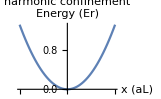

```mathematica
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Plot[potential[x,f0],{x,-50,50},PlotLabel->"harmonic confinement",AxesLabel->{"x (aL)","Energy (Er)"}]
```

```mathematica
onsiteU=0.407634 h kHz/Erecoil (174(1-7.5/(20-202.1)))/174 
tunnelling= 0.12642;(*unit is Erecoil*)
(*tempβ=4;*)
(*1/(kB Temp) = 1/Er*)
```

0.0943664

```mathematica
0.577687 h kHz/Erecoil(174(1-7.5/(20-202.1)))/174
```

0.133733

```mathematica
0.12642
```

0.12642

```mathematica
0.0943664
```

0.0943664

```mathematica
2.43759 h kHz/Erecoil (174(1-7.5/(20-202.1)))/174
```

0.564297

## manipulate folder list && calculate(1Er,t=0.178514,U=)

```mathematica
folderls={"20G",         "180G",     "197.5G","200G",     "201G",  "205G",       "206G",          "207G",          "210G",          "222Er",       "333Er",       "444Er",      "3.5Er",       "111Er",  "198G",   "199p5G",   "200p5G","15Er","555Er-200G"};
ttls=         {0.000001,     0.12642,  0.12642,   0.12642,   0.12642,0.12642,    0.12642,        0.12642, 0.12642,  0.14305,   0.111252,    0.0856614,  0.0976734,   0.178514,  0.12642,   0.12642,   0.12642,0.00653173, 0.0658986};
UUls=         {1.00001,0.121392,0.238406,0.414325, 0.70859,-0.143764, -0.0836618,-0.0480913, 0.00458904, 0.0758841, 0.113742,     0.154097,    0.133733,    0.0426963,    0.256427,   0.350277,  0.515478, 0.56297, 0.857072};
```

```mathematica
For[iifolder=19,iifolder≤ 19,iifolder++,
{
pathexp=StringJoin["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/","cubic-results-",folderls⟦iifolder⟧];
ttvalue=ttls⟦iifolder⟧;
UUvalue=UUls⟦iifolder⟧;
Print[StringJoin[ToString[folderls⟦iifolder⟧],"; t=",ToString[ttvalue],";U=",ToString[UUvalue]]];

calcedpath=StringJoin[pathexp,"/yes.txt"];
calcedcheck=Check[Import[calcedpath];True,False];
If[calcedcheck,
{
Print["calculated!"]
},
{
Print["start to calculate!"];
If[Length[StringCases[folderls⟦iifolder⟧,x_~~"G"-> x]]≥ 1,
{
Print["B field data sets"]
},
{
Print["lat depth data sets"];
(*trap freq*);
Vlatx=15;ToExpression[StringCases[folderls⟦iifolder⟧,x_~~"Er"-> x]⟦1⟧];(*unit: Er*);
Vlaty=Vlatx;
Vlatz=Vlatx;
bandnumber=6;
fx=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatz Er-√(Vlatz Er Er))/w0z^2))/(2π);
fy=√(2/massK40((2Vlatz Er-√(Vlatz Er Er))/w0z^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
fz=√(2/massK40((2Vlaty Er-√(Vlaty Er Er))/w0y^2+(2Vlatx Er-√(Vlatx Er Er))/w0x^2))/(2π);
f0= √(1*xdtfreq^2+fx^2);
potential[x_,f0x_]:=1/2 massK40 (2π f0x)^2(x λlat/2)^2/Erecoil;
Print["vlat=",ToString[Vlatx],";    f0=",ToString[f0]];
(*end of trap freq & potential*);
}
];

(*write geom file*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
tJold=ww⟦35⟧; 
onsiteUold=ww⟦60⟧;
tJnew=ttvalue;
onsiteUnew=UUvalue;
wwtJold1=StringJoin["0 0 1.0 0.0 0.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwtJold2=StringJoin["0 0 0.0 1.0 0.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwtJold3=StringJoin["0 0 0.0 0.0 1.0 ",ToString[tJold]," ",ToString[tJold]," 0.0"];
wwUold=     StringJoin["0 0 0.0 0.0 0.0 0.0 0.0 ",ToString[onsiteUold]];

wwtJnew1=StringJoin["0 0 1.0 0.0 0.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwtJnew2=StringJoin["0 0 0.0 1.0 0.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwtJnew3=StringJoin["0 0 0.0 0.0 1.0 ",ToString[tJnew]," ",ToString[tJnew]," 0.0"];
wwUnew=     StringJoin["0 0 0.0 0.0 0.0 0.0 0.0 ",ToString[onsiteUnew]];

writenew=StringReplace[writetemp,{wwtJold1-> wwtJnew1,wwtJold2-> wwtJnew2,wwtJold3-> wwtJnew3,wwUold-> wwUnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom",writenew,"Text"];
(*end of write geom file*);

(*start MC simulation*);

Run["clear"];

iitempstart=0.5001;iitempend=0.5002;δiitemp=0.041;
iiμstart=-0.5001;iiμend=-0.5001;δμ=0.0802;
(*save readme files*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
Export[StringJoin[pathexp,"/readme_in"],write,"Text"];

write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
Export[StringJoin[pathexp,"/readme_cubic.geom"],write,"Text"];
paralist={0,0};
paralist⟦1⟧={"iitempstart","iitempend","δiitemp","iiμstart","iiμend","δμ","onsiteU","tunnelling"};
paralist⟦2⟧={iitempstart,iitempend,δiitemp,iiμstart,iiμend,δμ,onsiteUnew,tJnew};
Export[StringJoin[pathexp,"/readme_paralist.txt"],paralist,"TSV"];

(*end save readme files*);
outputstring={"tempβ","μ","density","err","doublon","err","int_energy","err","kinetic_energy","err","total_energy","err"};
calcoutput={outputstring};
For[iitemp=iitempstart,iitemp≤ iitempend,iitemp=iitemp+δiitemp,
{
Print[Now];
iitempβ=1/iitemp;
Ltemp=50;
dtempβ=iitempβ/Ltemp;
Print[dtempβ];
Print["==========================================================="];
(*write the tempβ, into the in file for calculation*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwdτ=ww⟦Position[ww,"dtau"]⟦1,1⟧+1⟧;
wwL=ww⟦Position[ww,"L"]⟦1,1⟧+1⟧;

wwdτold=StringJoin["dtau   =  ",ToString[wwdτ]];
wwLold=  StringJoin["L      =  ",ToString[wwL]];

wwdτnew=StringJoin["dtau   =  ",ToString[dtempβ]];
wwLnew=  StringJoin["L      =  ",ToString[Ltemp]];

writenew=StringReplace[writetemp,{wwLold-> wwLnew,wwdτold-> wwdτnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*end of ..........*)(*write the tempβ, into the in file for calculation*);

For[iiμ=iiμstart,iiμ≤ iiμend,iiμ=iiμ+δμ,
{
If[Abs[iiμ]<0.00001,iiμ=0];
(*write the chemical potential μ into the in file for calculation*);
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwμup=ww⟦Position[ww,"up"]⟦1,1⟧+1⟧;
wwμdn=ww⟦Position[ww,"dn"]⟦1,1⟧+1⟧;

wwμupold=StringJoin["mu_up  =  ",ToString[wwμup]];
wwμdnold=StringJoin["mu_dn  =  ",ToString[wwμdn]];

wwμupnew=StringJoin["mu_up  =  ",ToString[iiμ]];
wwμdnnew=StringJoin["mu_dn  =  ",ToString[iiμ]];

writenew=StringReplace[writetemp,{wwμupold-> wwμupnew,wwμdnold-> wwμdnnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*write the chemical potential μ into the in file for calculation*);

(*run the program*);
Run["cd ~/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom; ./ggeom in"];
(*end of run the program*);

(*get results*);

out=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/test.out","TSV"];
(*density*);
outddensity=out⟦34,1⟧;
outb=TextCases[outddensity,"Word"];
density11=ToExpression[StringSplit[outb⟦2⟧,"E"]];
densityerr11=ToExpression[StringSplit[outb⟦3⟧,"E"]];
densitytemp=density11⟦1⟧*10^density11⟦2⟧;
densityerrtemp=densityerr11⟦1⟧*10^densityerr11⟦2⟧;
(*doublon density*);
outdoublon=out⟦45,1⟧;
outd=TextCases[outdoublon,"Word"];
doublon11=ToExpression[StringSplit[outd⟦3⟧,"E"]];
doublonerr11=ToExpression[StringSplit[outd⟦4⟧,"E"]];
doublontemp=doublon11⟦1⟧*10^doublon11⟦2⟧;
doublonerrtemp=doublonerr11⟦1⟧*10^doublonerr11⟦2⟧;
(*interaction energy*);
outint=out⟦31,1⟧;
outint11=TextCases[outint,"Word"];
outint22=ToExpression[StringSplit[outint11⟦2⟧,"E"]];
If[Length[outint22]==1,outint22=Join[outint22,{-20}]];
outinterr22=ToExpression[StringSplit[outint11⟦3⟧,"E"]];
If[Length[outinterr22]==1,outinterr22=Join[outinterr22,{-20}]];
outinttemp=outint22⟦1⟧*10^outint22⟦2⟧;
outinterrtemp=outinterr22⟦1⟧*10^outinterr22⟦2⟧;
(*kinetic energy*);
outkinetic=out⟦32,1⟧;
outkinetic11=TextCases[outkinetic,"Word"];
outkinetic22=ToExpression[StringSplit[outkinetic11⟦3⟧,"E"]];
If[Length[outkinetic22]==1,outkinetic22=Join[outkinetic22,{-20}]];
outkineticerr22=ToExpression[StringSplit[outkinetic11⟦4⟧,"E"]];
If[Length[outkineticerr22]==1,outkineticerr22=Join[outkineticerr22,{-20}]];
outkinetictemp=outkinetic22⟦1⟧*10^outkinetic22⟦2⟧;
outkineticerrtemp=outkineticerr22⟦1⟧*10^outkineticerr22⟦2⟧;
(*total energy*);
outtotalE=out⟦32,1⟧;
outtotalE11=TextCases[outtotalE,"Word"];
outtotalE22=ToExpression[StringSplit[outtotalE11⟦3⟧,"E"]];
If[Length[outtotalE22]==1,outtotalE22=Join[outtotalE22,{-20}]];
outtotalEerr22=ToExpression[StringSplit[outtotalE11⟦4⟧,"E"]];
If[Length[outtotalEerr22]==1,outtotalEerr22=Join[outtotalEerr22,{-20}]];
outtotalEtemp=outtotalE22⟦1⟧*10^outtotalE22⟦2⟧;
outtotalEerrtemp=outtotalEerr22⟦1⟧*10^outtotalEerr22⟦2⟧;

Print[StringJoin[
"tempβ:",ToString[iitempβ],"   ",
"μ :", ToString[iiμ],"    ",
"density :" ,ToString[densitytemp], "   ","err:", ToString[densityerrtemp],"     ",
"doublon:",ToString[doublontemp],"   ","err:",ToString[doublonerrtemp],"     ",
"int_energy",ToString[outinttemp],"    ","err:",ToString[outinterrtemp],"    ",
"kinetic_energy",ToString[outkinetictemp],"    ","err:",ToString[outkineticerrtemp],"    ",
"total_energy",ToString[outtotalEtemp],"    ","err:",ToString[outtotalEerrtemp]
]];
(*end of (*get results*)*)
(*outputstring={"tempβ","μ","density","err","doublon","err","int_energy","err","kinetic_energy","err","total_energy","err"};*)
outputtemp={iitempβ,iiμ,densitytemp,densityerrtemp,doublontemp,doublonerrtemp,outinttemp,outinterrtemp,outkinetictemp,outkineticerrtemp,outtotalEtemp,outtotalEerrtemp};
calcoutput=Join[calcoutput,{outputtemp}];

}
];
Print["END of CALCULATION!"];
}
];
Export[StringJoin[pathexp,"/calcoutput with energy.txt"],calcoutput,"TSV"];
Export[StringJoin[pathexp,"/yes.txt"],1];
(*end of MC simulation*);
Print["End of Exportation!"];
Print["///////////////////////////////////////////////////////////////////////////////////////"];
}];(*end of calcedcheck*);
};
]
```

555Er-200G; t=0.0658986;U=0.857072

Import::nffil: File not found during Import.

start to calculate!

B field data sets

Wed 4 Oct 2017 00:49:12GMT-4.

0.1

===========================================================

tempβ:5.   μ :-4.50001    density :          -9
4.06027 10   err:          -11
8.71497 10     doublon:          -19
2.73102 10   err:         -21
3.1914 10     int_energy          -19
2.34068 10    err:          -21
2.73526 10    kinetic_energy         -8
1.6025 10    err:          -10
3.48951 10    total_energy         -8
1.6025 10    err:          -10
3.48951 10

tempβ:5.   μ :-4.41981    density :          -9
6.06327 10   err:          -10
1.30142 10     doublon:          -19
6.09017 10   err:          -21
7.11682 10     int_energy          -19
5.21972 10    err:          -21
6.09963 10    kinetic_energy          -8
2.34442 10    err:          -10
5.10657 10    total_energy          -8
2.34442 10    err:          -10
5.10657 10

tempβ:5.   μ :-4.33961    density :          -9
9.05438 10   err:          -10
1.94343 10     doublon:          -18
1.35811 10   err:          -20
1.58705 10     int_energy        -18
1.164 10    err:          -20
1.36021 10    kinetic_energy          -8
3.42834 10    err:          -10
7.46986 10    total_energy          -8
3.42834 10    err:          -10
7.46986 10

tempβ:5.   μ :-4.25941    density :          -8
1.35211 10   err:          -10
2.90215 10     doublon:          -18
3.02858 10   err:          -20
3.53885 10     int_energy          -18
2.59571 10    err:          -20
3.03305 10    kinetic_energy          -8
5.01116 10    err:          -9
1.09221 10    total_energy          -8
5.01116 10    err:          -9
1.09221 10

tempβ:5.   μ :-4.17921    density :          -8
2.01912 10   err:          -10
4.33384 10     doublon:          -18
6.75371 10   err:          -20
7.89219 10     int_energy          -18
5.78841 10    err:          -20
6.76418 10    kinetic_energy          -8
7.32132 10    err:          -9
1.59626 10    total_energy          -8
7.32132 10    err:          -9
1.59626 10

tempβ:5.   μ :-4.09901    density :          -8
3.01519 10   err:          -10
6.47179 10     doublon:          -17
1.50607 10   err:          -19
1.75995 10     int_energy          -17
1.29081 10    err:          -19
1.50841 10    kinetic_energy          -7
1.06912 10    err:          -9
2.33181 10    total_energy          -7
1.06912 10    err:          -9
2.33181 10

tempβ:5.   μ :-4.01881    density :          -8
4.50264 10   err:          -10
9.66441 10     doublon:          -17
3.35854 10   err:          -19
3.92468 10     int_energy          -17
2.87851 10    err:          -19
3.36374 10    kinetic_energy          -7
1.56043 10    err:          -9
3.40462 10    total_energy          -7
1.56043 10    err:          -9
3.40462 10

tempβ:5.   μ :-3.93861    density :          -8
6.72386 10   err:         -9
1.4432 10     doublon:          -17
7.48953 10   err:        -19
8.752 10     int_energy          -17
6.41906 10    err:         -19
7.5011 10    kinetic_energy          -7
2.27629 10    err:          -9
4.96842 10    total_energy          -7
2.27629 10    err:          -9
4.96842 10

tempβ:5.   μ :-3.85841    density :          -7
1.00409 10   err:          -9
2.15514 10     doublon:          -16
1.67016 10   err:          -18
1.95168 10     int_energy          -16
1.43145 10    err:          -18
1.67273 10    kinetic_energy          -7
3.31869 10    err:          -9
7.24654 10    total_energy          -7
3.31869 10    err:          -9
7.24654 10

tempβ:5.   μ :-3.77821    density :          -7
1.49942 10   err:          -9
3.21828 10     doublon:          -16
3.72445 10   err:          -18
4.35222 10     int_energy          -16
3.19212 10    err:          -18
3.73017 10    kinetic_energy         -7
4.8356 10    err:          -8
1.05632 10    total_energy         -7
4.8356 10    err:          -8
1.05632 10

tempβ:5.   μ :-3.69801    density :         -7
2.2391 10   err:          -9
4.80586 10     doublon:          -16
8.30551 10   err:          -18
9.70534 10     int_energy          -16
7.11842 10    err:          -18
8.31817 10    kinetic_energy         -7
7.0415 10    err:          -8
1.53886 10    total_energy         -7
7.0415 10    err:          -8
1.53886 10

tempβ:5.   μ :-3.61781    density :          -7
3.34368 10   err:          -9
7.17654 10     doublon:          -15
1.85212 10   err:          -17
2.16425 10     int_energy         -15
1.5874 10    err:          -17
1.85492 10    kinetic_energy         -6
1.0247 10    err:         -8
2.2404 10    total_energy         -6
1.0247 10    err:         -8
2.2404 10

tempβ:5.   μ :-3.53761    density :          -7
4.99317 10   err:          -8
1.07167 10     doublon:          -15
4.13023 10   err:         -17
4.8261 10     int_energy          -15
3.53991 10    err:          -17
4.13632 10    kinetic_energy          -6
1.49016 10    err:          -8
3.25962 10    total_energy          -6
1.49016 10    err:          -8
3.25962 10

tempβ:5.   μ :-3.45741    density :          -7
7.45634 10   err:          -8
1.60026 10     doublon:          -15
9.21035 10   err:         -16
1.0762 10     int_energy          -15
7.89393 10    err:          -17
9.22379 10    kinetic_energy          -6
2.16546 10    err:          -8
4.73907 10    total_energy          -6
2.16546 10    err:          -8
4.73907 10

tempβ:5.   μ :-3.37721    density :          -6
1.11346 10   err:          -8
2.38954 10     doublon:         -14
2.0539 10   err:         -16
2.3998 10     int_energy          -14
1.76034 10    err:         -16
2.0568 10    kinetic_energy         -6
3.1444 10    err:          -8
6.88486 10    total_energy         -6
3.1444 10    err:          -8
6.88486 10

tempβ:5.   μ :-3.29701    density :         -6
1.6642 10   err:          -8
3.61247 10     doublon:          -14
4.57446 10   err:          -16
5.32242 10     int_energy          -14
3.92064 10    err:         -16
4.5617 10    kinetic_energy          -6
4.56636 10    err:          -7
1.01198 10    total_energy          -6
4.56636 10    err:          -7
1.01198 10

tempβ:5.   μ :-3.21681    density :          -6
2.48372 10   err:          -8
5.43261 10     doublon:         -13
1.0197 10   err:          -15
1.20177 10     int_energy          -14
8.73957 10    err:       -15
1.03 10    kinetic_energy          -6
6.61577 10    err:          -7
1.47873 10    total_energy          -6
6.61577 10    err:          -7
1.47873 10

tempβ:5.   μ :-3.13661    density :          -6
3.70889 10   err:         -8
8.1109 10     doublon:         -13
2.2739 10   err:          -15
2.67948 10     int_energy          -13
1.94889 10    err:          -15
2.29651 10    kinetic_energy          -6
9.58176 10    err:         -7
2.1427 10    total_energy          -6
9.58176 10    err:         -7
2.1427 10

tempβ:5.   μ :-3.05641    density :          -6
5.53848 10   err:          -7
1.17144 10     doublon:          -13
5.06648 10   err:          -15
5.68437 10     int_energy          -13
4.34234 10    err:          -15
4.87191 10    kinetic_energy0.0000138646    err:          -7
3.00133 10    total_energy0.0000138646    err:          -7
3.00133 10

tempβ:5.   μ :-2.97621    density :          -6
8.26431 10   err:          -7
1.72146 10     doublon:          -12
1.12913 10   err:          -14
1.20908 10     int_energy          -13
9.67744 10    err:          -14
1.03627 10    kinetic_energy0.0000200254    err:          -7
4.27088 10    total_energy0.0000200254    err:          -7
4.27088 10

tempβ:5.   μ :-2.89601    density :0.000012364   err:          -7
2.35693 10     doublon:          -12
2.51823 10   err:          -14
2.39478 10     int_energy          -12
2.15831 10    err:         -14
2.0525 10    kinetic_energy0.0000289698    err:          -7
5.66059 10    total_energy0.0000289698    err:          -7
5.66059 10

tempβ:5.   μ :-2.81581    density :0.0000184477   err:          -7
3.44506 10     doublon:          -12
5.60974 10   err:          -14
5.44624 10     int_energy          -12
4.80795 10    err:          -14
4.66782 10    kinetic_energy0.0000417441    err:          -7
7.99664 10    total_energy0.0000417441    err:          -7
7.99664 10

tempβ:5.   μ :-2.73561    density :0.0000275349   err:          -7
4.84933 10     doublon:          -11
1.25173 10   err:          -13
1.24302 10     int_energy          -11
1.07282 10    err:          -13
1.06536 10    kinetic_energy0.0000600993    err:          -6
1.08629 10    total_energy0.0000600993    err:          -6
1.08629 10

tempβ:5.   μ :-2.65541    density :0.0000412858   err:          -7
8.58829 10     doublon:          -11
2.78683 10   err:          -13
2.76748 10     int_energy          -11
2.38851 10    err:          -13
2.37193 10    kinetic_energy0.0000868192    err:          -6
1.86176 10    total_energy0.0000868192    err:          -6
1.86176 10

tempβ:5.   μ :-2.57521    density :0.000061813   err:          -6
1.23994 10     doublon:          -11
6.21566 10   err:          -13
5.07304 10     int_energy          -11
5.32726 10    err:          -13
4.34796 10    kinetic_energy0.000125046    err:          -6
2.59145 10    total_energy0.000125046    err:          -6
2.59145 10

tempβ:5.   μ :-2.49501    density :0.0000924937   err:         -6
1.7969 10     doublon:          -10
1.38461 10   err:          -12
1.47926 10     int_energy          -10
1.18671 10    err:          -12
1.26783 10    kinetic_energy0.000179703    err:          -6
3.61715 10    total_energy0.000179703    err:          -6
3.61715 10

tempβ:5.   μ :-2.41481    density :0.000136951   err:          -6
2.41908 10     doublon:          -10
3.08695 10   err:          -12
2.61387 10     int_energy          -10
2.64574 10    err:          -12
2.24027 10    kinetic_energy0.000255004    err:          -6
4.68937 10    total_energy0.000255004    err:          -6
4.68937 10

tempβ:5.   μ :-2.33461    density :0.000201219   err:          -6
3.37595 10     doublon:          -10
6.86036 10   err:          -12
7.77977 10     int_energy          -10
5.87982 10    err:          -12
6.66782 10    kinetic_energy0.000358284    err:          -6
6.25246 10    total_energy0.000358284    err:          -6
6.25246 10

tempβ:5.   μ :-2.25441    density :0.000303696   err:          -6
4.04853 10     doublon:          -9
1.54005 10   err:          -11
2.02067 10     int_energy          -9
1.31994 10    err:          -11
1.73186 10    kinetic_energy0.000516553    err:          -6
7.12501 10    total_energy0.000516553    err:          -6
7.12501 10

tempβ:5.   μ :-2.17421    density :0.000442461   err:          -6
8.23657 10     doublon:          -9
3.36623 10   err:         -11
3.0467 10     int_energy         -9
2.8851 10    err:          -11
2.61124 10    kinetic_energy0.000716442    err:0.0000139366    total_energy0.000716442    err:0.0000139366

tempβ:5.   μ :-2.09401    density :0.000660283   err:          -6
7.27599 10     doublon:          -9
7.49412 10   err:          -11
4.86542 10     int_energy        -9
6.423 10    err:          -11
4.17002 10    kinetic_energy0.00101631    err:0.0000117819    total_energy0.00101631    err:0.0000117819

tempβ:5.   μ :-2.01381    density :0.000977513   err:0.0000150727     doublon:          -8
1.66943 10   err:          -10
1.60474 10     int_energy          -8
1.43082 10    err:          -10
1.37538 10    kinetic_energy0.00142639    err:0.0000230126    total_energy0.00142639    err:0.0000230126

tempβ:5.   μ :-1.93361    density :0.00146701   err:0.0000149754     doublon:          -8
3.76864 10   err:          -10
1.03738 10     int_energy          -8
3.22999 10    err:          -11
8.89107 10    kinetic_energy0.00202238    err:0.0000217275    total_energy0.00202238    err:0.0000217275

tempβ:5.   μ :-1.85341    density :0.00220016   err:0.0000172545     doublon:          -8
8.39271 10   err:          -10
6.68182 10     int_energy          -8
7.19315 10    err:         -10
5.7268 10    kinetic_energy0.00285677    err:0.0000236079    total_energy0.00285677    err:0.0000236079

tempβ:5.   μ :-1.77321    density :0.00327728   err:0.0000453894     doublon:          -7
1.86719 10   err:          -9
2.07915 10     int_energy          -7
1.60032 10    err:          -9
1.78198 10    kinetic_energy0.00399497    err:0.0000577879    total_energy0.00399497    err:0.0000577879

tempβ:5.   μ :-1.69301    density :0.00494525   err:0.0000469461     doublon:          -7
4.19524 10   err:         -9
5.5305 10     int_energy          -7
3.59562 10    err:          -9
4.74004 10    kinetic_energy0.00563503    err:0.0000563316    total_energy0.00563503    err:0.0000563316

tempβ:5.   μ :-1.61281    density :0.00712846   err:0.0000516288     doublon:          -7
9.01491 10   err:          -8
1.15253 10     int_energy          -7
7.72643 10    err:          -9
9.87797 10    kinetic_energy0.0075412    err:0.0000570354    total_energy0.0075412    err:0.0000570354

tempβ:5.   μ :-1.53261    density :0.0105841   err:0.000111922     doublon:          -6
2.00262 10   err:         -8
1.6531 10     int_energy          -6
1.71639 10    err:          -8
1.41683 10    kinetic_energy0.0103521    err:0.000112481    total_energy0.0103521    err:0.000112481

tempβ:5.   μ :-1.45241    density :0.016352   err:0.000211698     doublon:         -6
4.5161 10   err:          -8
5.69179 10     int_energy          -6
3.87062 10    err:          -8
4.87828 10    kinetic_energy0.0147309    err:0.000203468    total_energy0.0147309    err:0.000203468

tempβ:5.   μ :-1.37221    density :0.0234417   err:0.000333663     doublon:          -6
9.64694 10   err:          -7
1.41372 10     int_energy          -6
8.26813 10    err:          -7
1.21166 10    kinetic_energy0.0192222    err:0.000293526    total_energy0.0192222    err:0.000293526

tempβ:5.   μ :-1.29201    density :0.0349997   err:0.000327238     doublon:0.0000209918   err:          -8
9.58918 10     int_energy0.0000179915    err:          -8
8.21862 10    kinetic_energy0.025973    err:0.000258468    total_energy0.025973    err:0.000258468

tempβ:5.   μ :-1.21181    density :0.0504386   err:0.000329655     doublon:0.0000446502   err:          -7
2.45743 10     int_energy0.0000382685    err:          -7
2.10619 10    kinetic_energy0.0334865    err:0.000242701    total_energy0.0334865    err:0.000242701

tempβ:5.   μ :-1.13161    density :0.0743712   err:0.000444711     doublon:0.0000939378   err:          -7
6.12013 10     int_energy0.0000805114    err:         -7
5.2454 10    kinetic_energy0.0436183    err:0.000281859    total_energy0.0436183    err:0.000281859

tempβ:5.   μ :-1.05141    density :0.103757   err:0.00109064     doublon:0.000189267   err:          -7
6.71244 10     int_energy0.000162216    err:          -7
5.75305 10    kinetic_energy0.0528249    err:0.000636335    total_energy0.0528249    err:0.000636335

tempβ:5.   μ :-0.97121    density :0.146032   err:0.00101568     doublon:0.000376342   err:          -6
2.49871 10     int_energy0.000322552    err:          -6
2.14158 10    kinetic_energy0.0633823    err:0.000508662    total_energy0.0633823    err:0.000508662

tempβ:5.   μ :-0.89101    density :0.198397   err:0.001078     doublon:0.000705514   err:          -6
2.06719 10     int_energy0.000604676    err:          -6
1.77173 10    kinetic_energy0.0712874    err:0.000479386    total_energy0.0712874    err:0.000479386

tempβ:5.   μ :-0.81081    density :0.261824   err:0.00166825     doublon:0.00127826   err:          -6
5.00809 10     int_energy0.00109556    err:          -6
4.29229 10    kinetic_energy0.0747252    err:0.000589823    total_energy0.0747252    err:0.000589823

tempβ:5.   μ :-0.73061    density :0.337684   err:0.00102969     doublon:0.00221906   err:          -6
3.01353 10     int_energy0.0019019    err:          -6
2.58281 10    kinetic_energy0.0715593    err:0.000315484    total_energy0.0715593    err:0.000315484

tempβ:5.   μ :-0.65041    density :0.424612   err:0.000973403     doublon:0.00362858   err:          -6
8.81952 10     int_energy0.00310995    err:          -6
7.55896 10    kinetic_energy0.0597096    err:0.00022544    total_energy0.0597096    err:0.00022544

tempβ:5.   μ :-0.57021    density :0.513837   err:0.00131432     doublon:0.0057312   err:0.0000146751     int_energy0.00491205    err:0.0000125776    kinetic_energy0.0351709    err:0.000183824    total_energy0.0351709    err:0.000183824

tempβ:5.   μ :-0.49001    density :0.604951   err:0.00198903     doublon:0.00864103   err:0.0000502763     int_energy0.00740599    err:0.0000430904    kinetic_energy0.00226524    err:0.000300496    total_energy0.00226524    err:0.000300496

tempβ:5.   μ :-0.40981    density :0.692447   err:0.00119371     doublon:0.0125472   err:0.0000398878     int_energy0.0107539    err:0.0000341867    kinetic_energy0.0527562    err:0.0000903148    total_energy0.0527562    err:0.0000903148

tempβ:5.   μ :-0.32961    density :0.770138   err:0.000883799     doublon:0.0178797   err:0.0000809123     int_energy0.0153242    err:0.0000693477    kinetic_energy0.115489    err:0.0000678566    total_energy0.115489    err:0.0000678566

tempβ:5.   μ :-0.24941    density :0.838661   err:0.000654123     doublon:0.0250075   err:0.0000780056     int_energy0.0214333    err:0.0000668564    kinetic_energy0.188459    err:0.0000651925    total_energy0.188459    err:0.0000651925

tempβ:5.   μ :-0.16921    density :0.897191   err:0.00026511     doublon:0.0348675   err:0.000104214     int_energy0.029884    err:0.0000893186    kinetic_energy0.269886    err:0.0000587742    total_energy0.269886    err:0.0000587742

tempβ:5.   μ :-0.08901    density :0.947826   err:0.000272617     doublon:0.0488333   err:0.000236314     int_energy0.0418537    err:0.000202538    kinetic_energy0.358407    err:0.0000609994    total_energy0.358407    err:0.0000609994

tempβ:5.   μ :-0.00881    density :0.994942   err:0.0000293448     doublon:0.0677338   err:0.000381083     int_energy0.0580528    err:0.000326616    kinetic_energy0.453923    err:0.000120743    total_energy0.453923    err:0.000120743

tempβ:5.   μ :0.07139    density :1.04148   err:0.000193521     doublon:0.0938564   err:0.000434872     int_energy0.0804417    err:0.000372717    kinetic_energy0.557134    err:0.000228745    total_energy0.557134    err:0.000228745

tempβ:5.   μ :0.15159    density :1.09113   err:0.000765013     doublon:0.128687   err:0.0010866     int_energy0.110294    err:0.000931297    kinetic_energy0.670092    err:0.00068678    total_energy0.670092    err:0.00068678

tempβ:5.   μ :0.23179    density :1.14781   err:0.000459625     doublon:0.174771   err:0.000559366     int_energy0.149791    err:0.000479417    kinetic_energy0.795981    err:0.000432133    total_energy0.795981    err:0.000432133

tempβ:5.   μ :0.31199    density :1.21508   err:0.000822283     doublon:0.234492   err:0.000898377     int_energy0.200976    err:0.000769974    kinetic_energy0.939078    err:0.00073068    total_energy0.939078    err:0.00073068

tempβ:5.   μ :0.39219    density :1.28882   err:0.000604224     doublon:0.302378   err:0.000643959     int_energy0.25916    err:0.000551919    kinetic_energy1.09743    err:0.000587086    total_energy1.09743    err:0.000587086

tempβ:5.   μ :0.47239    density :1.37488   err:0.000859901     doublon:0.384271   err:0.000883408     int_energy0.329348    err:0.000757145    kinetic_energy1.27825    err:0.000880596    total_energy1.27825    err:0.000880596

tempβ:5.   μ :0.55259    density :1.46417   err:0.00067795     doublon:0.470468   err:0.000678344     int_energy0.403225    err:0.000581389    kinetic_energy1.47478    err:0.000671115    total_energy1.47478    err:0.000671115

tempβ:5.   μ :0.63279    density :1.55425   err:0.00113741     doublon:0.558277   err:0.0011453     int_energy0.478484    err:0.000981609    kinetic_energy1.68483    err:0.00122675    total_energy1.68483    err:0.00122675

tempβ:5.   μ :0.71299    density :1.64363   err:0.00156812     doublon:0.646107   err:0.00156861     int_energy0.55376    err:0.00134441    kinetic_energy1.90761    err:0.00178074    total_energy1.90761    err:0.00178074

tempβ:5.   μ :0.79319    density :1.72215   err:0.000834923     doublon:0.723593   err:0.000830837     int_energy0.620171    err:0.000712087    kinetic_energy2.13062    err:0.000990277    total_energy2.13062    err:0.000990277

tempβ:5.   μ :0.87339    density :1.78794   err:0.000567784     doublon:0.788746   err:0.000567247     int_energy0.676013    err:0.000486172    kinetic_energy2.34932    err:0.000724459    total_energy2.34932    err:0.000724459

tempβ:5.   μ :0.95359    density :1.84366   err:0.000344446     doublon:0.844089   err:0.000344511     int_energy0.723445    err:0.00029527    kinetic_energy2.56499    err:0.000459899    total_energy2.56499    err:0.000459899

END of CALCULATION!

Wed 4 Oct 2017 05:32:26GMT-4.

0.0829876

===========================================================

tempβ:4.14938   μ :-4.50001    density :          -7
1.16984 10   err:          -9
1.92276 10     doublon:          -16
2.50463 10   err:          -18
1.72729 10     int_energy          -16
2.14664 10    err:          -18
1.48042 10    kinetic_energy         -7
4.6404 10    err:          -9
7.71839 10    total_energy         -7
4.6404 10    err:          -9
7.71839 10

tempβ:4.14938   μ :-4.41981    density :          -7
1.63174 10   err:          -9
2.68192 10     doublon:          -16
4.87295 10   err:          -18
3.36058 10     int_energy          -16
4.17647 10    err:          -18
2.88026 10    kinetic_energy          -7
6.34175 10    err:          -8
1.05508 10    total_energy          -7
6.34175 10    err:          -8
1.05508 10

tempβ:4.14938   μ :-4.33961    density :          -7
2.27602 10   err:          -9
3.74083 10     doublon:          -16
9.48071 10   err:          -18
6.53823 10     int_energy          -16
8.12565 10    err:          -18
5.60374 10    kinetic_energy          -7
8.66319 10    err:          -8
1.44165 10    total_energy          -7
8.66319 10    err:          -8
1.44165 10

tempβ:4.14938   μ :-4.25941    density :          -7
3.17468 10   err:          -9
5.21781 10     doublon:          -15
1.84455 10   err:          -17
1.27206 10     int_energy          -15
1.58091 10    err:          -17
1.09024 10    kinetic_energy          -6
1.18292 10    err:          -8
1.96901 10    total_energy          -6
1.18292 10    err:          -8
1.96901 10

tempβ:4.14938   μ :-4.17921    density :          -7
4.42817 10   err:          -9
7.27792 10     doublon:          -15
3.58871 10   err:          -17
2.47486 10     int_energy          -15
3.07579 10    err:          -17
2.12113 10    kinetic_energy          -6
1.61446 10    err:          -8
2.68805 10    total_energy          -6
1.61446 10    err:          -8
2.68805 10

tempβ:4.14938   μ :-4.09901    density :          -7
6.17658 10   err:          -8
1.01513 10     doublon:          -15
6.98213 10   err:          -17
4.81496 10     int_energy          -15
5.98418 10    err:          -17
4.12677 10    kinetic_energy          -6
2.20238 10    err:          -8
3.66791 10    total_energy          -6
2.20238 10    err:          -8
3.66791 10

tempβ:4.14938   μ :-4.01881    density :          -7
8.61532 10   err:          -8
1.41591 10     doublon:          -14
1.35843 10   err:          -17
9.36767 10     int_energy          -14
1.16427 10    err:          -17
8.02877 10    kinetic_energy          -6
3.00286 10    err:          -8
5.00246 10    total_energy          -6
3.00286 10    err:          -8
5.00246 10

tempβ:4.14938   μ :-3.93861    density :         -6
1.2017 10   err:         -8
1.9749 10     doublon:          -14
2.64292 10   err:         -16
1.8225 10     int_energy          -14
2.26518 10    err:          -16
1.56201 10    kinetic_energy          -6
4.09212 10    err:          -8
6.81899 10    total_energy          -6
4.09212 10    err:          -8
6.81899 10

tempβ:4.14938   μ :-3.85841    density :          -6
1.67667 10   err:          -8
2.77857 10     doublon:          -14
5.13788 10   err:          -16
3.53327 10     int_energy          -14
4.40353 10    err:          -16
3.02826 10    kinetic_energy          -6
5.57514 10    err:          -8
9.37292 10    total_energy          -6
5.57514 10    err:          -8
9.37292 10

tempβ:4.14938   μ :-3.77821    density :          -6
2.33886 10   err:          -8
3.89902 10     doublon:          -14
9.99693 10   err:          -16
6.90511 10     int_energy          -14
8.56809 10    err:          -16
5.91818 10    kinetic_energy          -6
7.58939 10    err:          -7
1.28379 10    total_energy          -6
7.58939 10    err:          -7
1.28379 10

tempβ:4.14938   μ :-3.69801    density :          -6
3.26069 10   err:          -8
5.47719 10     doublon:          -13
1.94446 10   err:          -15
1.36934 10     int_energy          -13
1.66655 10    err:          -15
1.17362 10    kinetic_energy0.0000103191    err:          -7
1.75986 10    total_energy0.0000103191    err:          -7
1.75986 10

tempβ:4.14938   μ :-3.61781    density :          -6
4.54807 10   err:          -8
7.63869 10     doublon:          -13
3.78308 10   err:          -15
2.66384 10     int_energy          -13
3.24237 10    err:         -15
2.2831 10    kinetic_energy0.0000140285    err:         -7
2.3931 10    total_energy0.0000140285    err:         -7
2.3931 10

tempβ:4.14938   μ :-3.53761    density :          -6
6.34245 10   err:          -7
1.01811 10     doublon:          -13
7.35404 10   err:          -15
4.87707 10     int_energy          -13
6.30294 10    err:       -15
4.18 10    kinetic_energy0.000019055    err:         -7
3.1085 10    total_energy0.000019055    err:         -7
3.1085 10

tempβ:4.14938   μ :-3.45741    density :          -6
8.84286 10   err:          -7
1.40749 10     doublon:          -12
1.43066 10   err:          -15
9.05675 10     int_energy          -12
1.22618 10    err:          -15
7.76228 10    kinetic_energy0.0000258577    err:         -7
4.1831 10    total_energy0.0000258577    err:         -7
4.1831 10

tempβ:4.14938   μ :-3.37721    density :0.0000123474   err:          -7
1.82449 10     doublon:          -12
2.78394 10   err:          -14
1.56583 10     int_energy          -12
2.38603 10    err:          -14
1.34203 10    kinetic_energy0.0000351163    err:          -7
5.27721 10    total_energy0.0000351163    err:          -7
5.27721 10

tempβ:4.14938   μ :-3.29701    density :0.0000172152   err:          -7
2.51918 10     doublon:          -12
5.41477 10   err:          -14
3.11986 10     int_energy          -12
4.64085 10    err:          -14
2.67394 10    kinetic_energy0.0000475794    err:          -7
7.08276 10    total_energy0.0000475794    err:          -7
7.08276 10

tempβ:4.14938   μ :-3.21681    density :0.0000240243   err:          -7
3.53621 10     doublon:          -11
1.05379 10   err:         -14
5.8596 10     int_energy          -12
9.03174 10    err:         -14
5.0221 10    kinetic_energy0.0000644736    err:          -7
9.66183 10    total_energy0.0000644736    err:          -7
9.66183 10

tempβ:4.14938   μ :-3.13661    density :0.0000336131   err:          -7
5.17749 10     doublon:          -11
2.04949 10   err:          -13
1.30774 10     int_energy          -11
1.75656 10    err:          -13
1.12083 10    kinetic_energy0.0000875183    err:          -6
1.37587 10    total_energy0.0000875183    err:          -6
1.37587 10

tempβ:4.14938   μ :-3.05641    density :0.0000468719   err:          -7
7.03461 10     doublon:          -11
3.99036 10   err:          -13
2.25846 10     int_energy          -11
3.42003 10    err:          -13
1.93567 10    kinetic_energy0.000118281    err:          -6
1.81226 10    total_energy0.000118281    err:          -6
1.81226 10

tempβ:4.14938   μ :-2.97621    density :0.0000655162   err:          -7
9.71168 10     doublon:          -11
7.75849 10   err:          -13
3.72779 10     int_energy          -11
6.64959 10    err:          -13
3.19498 10    kinetic_energy0.000160089    err:          -6
2.42531 10    total_energy0.000160089    err:          -6
2.42531 10

tempβ:4.14938   μ :-2.89601    density :0.0000913313   err:          -6
1.29375 10     doublon:          -10
1.50741 10   err:          -13
8.49726 10     int_energy          -10
1.29196 10    err:          -13
7.28276 10    kinetic_energy0.00021584    err:          -6
3.12743 10    total_energy0.00021584    err:          -6
3.12743 10

tempβ:4.14938   μ :-2.81581    density :0.000127173   err:          -6
1.54922 10     doublon:          -10
2.93282 10   err:          -12
1.53989 10     int_energy          -10
2.51364 10    err:         -12
1.3198 10    kinetic_energy0.00029033    err:          -6
3.63701 10    total_energy0.00029033    err:          -6
3.63701 10

tempβ:4.14938   μ :-2.73561    density :0.000176289   err:          -6
2.17312 10     doublon:          -10
5.69929 10   err:          -12
2.93543 10     int_energy         -10
4.8847 10    err:          -12
2.51587 10    kinetic_energy0.000388271    err:          -6
4.92583 10    total_energy0.000388271    err:          -6
4.92583 10

tempβ:4.14938   μ :-2.65541    density :0.000243982   err:          -6
3.58035 10     doublon:          -9
1.10758 10   err:          -12
8.70945 10     int_energy          -10
9.49273 10    err:          -12
7.46463 10    kinetic_energy0.000517643    err:          -6
7.80259 10    total_energy0.000517643    err:          -6
7.80259 10

tempβ:4.14938   μ :-2.57521    density :0.000342829   err:          -6
2.86623 10     doublon:          -9
2.16299 10   err:          -11
1.66751 10     int_energy          -9
1.85384 10    err:          -11
1.42918 10    kinetic_energy0.000699979    err:          -6
6.01418 10    total_energy0.000699979    err:          -6
6.01418 10

tempβ:4.14938   μ :-2.49501    density :0.000471509   err:          -6
8.26706 10     doublon:          -9
4.17448 10   err:          -11
2.78856 10     int_energy          -9
3.57783 10    err:          -11
2.38999 10    kinetic_energy0.000924513    err:0.0000167252    total_energy0.000924513    err:0.0000167252

tempβ:4.14938   μ :-2.41481    density :0.0006562   err:          -6
8.37404 10     doublon:          -9
8.11942 10   err:          -11
4.03391 10     int_energy          -9
6.95893 10    err:          -11
3.45736 10    kinetic_energy0.00123416    err:0.0000163212    total_energy0.00123416    err:0.0000163212

tempβ:4.14938   μ :-2.33461    density :0.000916013   err:          -6
8.27708 10     doublon:          -8
1.58417 10   err:          -10
1.25831 10     int_energy          -8
1.35775 10    err:          -10
1.07846 10    kinetic_energy0.00164956    err:0.0000152319    total_energy0.00164956    err:0.0000152319

tempβ:4.14938   μ :-2.25441    density :0.00129114   err:0.000011894     doublon:          -8
3.07328 10   err:          -10
1.59819 10     int_energy          -8
2.63403 10    err:          -10
1.36976 10    kinetic_energy0.00222155    err:0.0000211324    total_energy0.00222155    err:0.0000211324

tempβ:4.14938   μ :-2.17421    density :0.00175049   err:0.0000108385     doublon:          -8
5.95149 10   err:          -10
2.40774 10     int_energy          -8
5.10086 10    err:          -10
2.06361 10    kinetic_energy0.00286962    err:0.0000184854    total_energy0.00286962    err:0.0000184854

tempβ:4.14938   μ :-2.09401    density :0.0024834   err:0.0000121748     doublon:          -7
1.15678 10   err:          -10
5.88013 10     int_energy          -8
9.91446 10    err:          -10
5.03969 10    kinetic_energy0.00387528    err:0.0000195515    total_energy0.00387528    err:0.0000195515

tempβ:4.14938   μ :-2.01381    density :0.00341517   err:0.0000123662     doublon:          -7
2.26698 10   err:          -9
1.14191 10     int_energy          -7
1.94297 10    err:          -10
9.78697 10    kinetic_energy0.00505232    err:0.0000187842    total_energy0.00505232    err:0.0000187842

tempβ:4.14938   μ :-1.93361    density :0.00481535   err:0.0000544836     doublon:          -7
4.37835 10   err:          -9
1.95951 10     int_energy          -7
3.75256 10    err:          -9
1.67944 10    kinetic_energy0.00674145    err:0.0000788812    total_energy0.00674145    err:0.0000788812

tempβ:4.14938   μ :-1.85341    density :0.00670784   err:0.0000924369     doublon:          -7
8.49938 10   err:          -9
6.45169 10     int_energy          -7
7.28458 10    err:          -9
5.52957 10    kinetic_energy0.00885568    err:0.00012579    total_energy0.00885568    err:0.00012579

tempβ:4.14938   μ :-1.77321    density :0.00951262   err:0.0000633342     doublon:          -6
1.66912 10   err:         -8
1.1849 10     int_energy          -6
1.43056 10    err:          -8
1.01554 10    kinetic_energy0.011808    err:0.0000814598    total_energy0.011808    err:0.0000814598

tempβ:4.14938   μ :-1.69301    density :0.0130024   err:0.000125767     doublon:          -6
3.18115 10   err:          -8
1.41337 10     int_energy          -6
2.72648 10    err:          -8
1.21136 10    kinetic_energy0.0150894    err:0.000149873    total_energy0.0150894    err:0.000149873

tempβ:4.14938   μ :-1.61281    density :0.0177598   err:0.000211605     doublon:          -6
6.10415 10   err:          -8
3.55018 10     int_energy         -6
5.2317 10    err:          -8
3.04276 10    kinetic_energy0.019173    err:0.000236848    total_energy0.019173    err:0.000236848

tempβ:4.14938   μ :-1.53261    density :0.0245851   err:0.000149297     doublon:0.0000116254   err:          -8
4.95728 10     int_energy          -6
9.96381 10    err:          -8
4.24875 10    kinetic_energy0.0246026    err:0.000158917    total_energy0.0246026    err:0.000158917

tempβ:4.14938   μ :-1.45241    density :0.0341823   err:0.000277532     doublon:0.0000222358   err:          -8
9.50833 10     int_energy0.0000190577    err:          -8
8.14932 10    kinetic_energy0.031512    err:0.000272213    total_energy0.031512    err:0.000272213

tempβ:4.14938   μ :-1.37221    density :0.0468826   err:0.000155348     doublon:0.0000418288   err:          -7
1.04364 10     int_energy0.0000358503    err:          -8
8.94474 10    kinetic_energy0.0395031    err:0.000135668    total_energy0.0395031    err:0.000135668

tempβ:4.14938   μ :-1.29201    density :0.0633322   err:0.000346136     doublon:0.0000785313   err:          -7
1.65337 10     int_energy0.000067307    err:          -7
1.41706 10    kinetic_energy0.0483544    err:0.000289817    total_energy0.0483544    err:0.000289817

tempβ:4.14938   μ :-1.21181    density :0.0865545   err:0.000405729     doublon:0.000145349   err:          -7
4.51192 10     int_energy0.000124574    err:          -7
3.86704 10    kinetic_energy0.0593701    err:0.000284002    total_energy0.0593701    err:0.000284002

tempβ:4.14938   μ :-1.13161    density :0.114039   err:0.000863929     doublon:0.000262834   err:          -7
7.25271 10     int_energy0.000225268    err:          -7
6.21609 10    kinetic_energy0.0692615    err:0.000551393    total_energy0.0692615    err:0.000551393

tempβ:4.14938   μ :-1.05141    density :0.15105   err:0.00075839     doublon:0.00046558   err:          -7
7.98987 10     int_energy0.000399036    err:         -7
6.8479 10    kinetic_energy0.0800807    err:0.000447165    total_energy0.0800807    err:0.000447165

tempβ:4.14938   μ :-0.97121    density :0.198438   err:0.000379336     doublon:0.000810837   err:         -6
1.3723 10     int_energy0.000694945    err:          -6
1.17616 10    kinetic_energy0.0902354    err:0.000174141    total_energy0.0902354    err:0.000174141

tempβ:4.14938   μ :-0.89101    density :0.254483   err:0.000897088     doublon:0.0013715   err:          -6
1.41162 10     int_energy0.00117547    err:          -6
1.20986 10    kinetic_energy0.0964329    err:0.000385797    total_energy0.0964329    err:0.000385797

tempβ:4.14938   μ :-0.81081    density :0.317138   err:0.000269765     doublon:0.00224913   err:          -6
2.07683 10     int_energy0.00192766    err:          -6
1.77999 10    kinetic_energy0.0962699    err:0.00010342    total_energy0.0962699    err:0.00010342

tempβ:4.14938   μ :-0.73061    density :0.387359   err:0.00107086     doublon:0.00357537   err:          -6
2.84388 10     int_energy0.00306435    err:          -6
2.43741 10    kinetic_energy0.0885508    err:0.000340376    total_energy0.0885508    err:0.000340376

tempβ:4.14938   μ :-0.65041    density :0.466678   err:0.00147604     doublon:0.00550016   err:         -6
9.2861 10     int_energy0.00471403    err:          -6
7.95886 10    kinetic_energy0.0720981    err:0.000263225    total_energy0.0720981    err:0.000263225

tempβ:4.14938   μ :-0.57021    density :0.544207   err:0.0015482     doublon:0.00826605   err:0.0000246178     int_energy0.0070846    err:0.0000210992    kinetic_energy0.0434255    err:0.000259746    total_energy0.0434255    err:0.000259746

tempβ:4.14938   μ :-0.49001    density :0.622537   err:0.000753326     doublon:0.0120402   err:0.0000232406     int_energy0.0103193    err:0.0000199189    kinetic_energy0.00331106    err:0.0000953339    total_energy0.00331106    err:0.0000953339

tempβ:4.14938   μ :-0.40981    density :0.700064   err:0.000751638     doublon:0.0171372   err:0.0000403836     int_energy0.0146878    err:0.0000346117    kinetic_energy0.0486965    err:0.0000424624    total_energy0.0486965    err:0.0000424624

tempβ:4.14938   μ :-0.32961    density :0.768216   err:0.000461098     doublon:0.0241667   err:0.0000451585     int_energy0.0207126    err:0.0000387041    kinetic_energy0.111709    err:0.0000722451    total_energy0.111709    err:0.0000722451

tempβ:4.14938   μ :-0.24941    density :0.833284   err:0.000643826     doublon:0.033268   err:0.000112175     int_energy0.0285131    err:0.0000961419    kinetic_energy0.184598    err:0.0000732303    total_energy0.184598    err:0.0000732303

tempβ:4.14938   μ :-0.16921    density :0.89063   err:0.000102122     doublon:0.0456449   err:0.0000589231     int_energy0.039121    err:0.0000505013    kinetic_energy0.265867    err:0.0000806474    total_energy0.265867    err:0.0000806474

tempβ:4.14938   μ :-0.08901    density :0.944118   err:0.000209486     doublon:0.0617313   err:0.000218504     int_energy0.0529082    err:0.000187273    kinetic_energy0.355094    err:0.0000227119    total_energy0.355094    err:0.0000227119

tempβ:4.14938   μ :-0.00881    density :0.994522   err:0.0000197282     doublon:0.0830581   err:0.000300072     int_energy0.0711867    err:0.000257183    kinetic_energy0.451874    err:0.0000961067    total_energy0.451874    err:0.0000961067

tempβ:4.14938   μ :0.07139    density :1.04496   err:0.00013777     doublon:0.111307   err:0.000323525     int_energy0.0953982    err:0.000277284    kinetic_energy0.557039    err:0.000113877    total_energy0.557039    err:0.000113877

tempβ:4.14938   μ :0.15159    density :1.09672   err:0.000388017     doublon:0.14529   err:0.000587548     int_energy0.124524    err:0.000503571    kinetic_energy0.670997    err:0.00034484    total_energy0.670997    err:0.00034484

tempβ:4.14938   μ :0.23179    density :1.15371   err:0.000570138     doublon:0.18939   err:0.000692863     int_energy0.162321    err:0.000593833    kinetic_energy0.797073    err:0.000471448    total_energy0.797073    err:0.000471448

tempβ:4.14938   μ :0.31199    density :1.21543   err:0.000263108     doublon:0.241192   err:0.000309704     int_energy0.206719    err:0.000265439    kinetic_energy0.935544    err:0.000257453    total_energy0.935544    err:0.000257453

tempβ:4.14938   μ :0.39219    density :1.28557   err:0.000604106     doublon:0.304137   err:0.000639197     int_energy0.260668    err:0.000547838    kinetic_energy1.09087    err:0.000555458    total_energy1.09087    err:0.000555458

tempβ:4.14938   μ :0.47239    density :1.35967   err:0.000803613     doublon:0.372695   err:0.000822092     int_energy0.319427    err:0.000704592    kinetic_energy1.26007    err:0.000766004    total_energy1.26007    err:0.000766004

tempβ:4.14938   μ :0.55259    density :1.43784   err:0.00161721     doublon:0.446819   err:0.00163276     int_energy0.382956    err:0.00139939    kinetic_energy1.44473    err:0.00159603    total_energy1.44473    err:0.00159603

tempβ:4.14938   μ :0.63279    density :1.5184   err:0.001178     doublon:0.524447   err:0.0011915     int_energy0.449489    err:0.0010212    kinetic_energy1.64352    err:0.00129264    total_energy1.64352    err:0.00129264

tempβ:4.14938   μ :0.71299    density :1.59711   err:0.00136096     doublon:0.601045   err:0.00136916     int_energy0.515139    err:0.00117347    kinetic_energy1.85225    err:0.00156515    total_energy1.85225    err:0.00156515

tempβ:4.14938   μ :0.79319    density :1.6674   err:0.000788624     doublon:0.669893   err:0.000790837     int_energy0.574146    err:0.000677804    kinetic_energy2.06287    err:0.000970357    total_energy2.06287    err:0.000970357

tempβ:4.14938   μ :0.87339    density :1.73383   err:0.000945743     doublon:0.735369   err:0.00094476     int_energy0.630265    err:0.000809728    kinetic_energy2.27938    err:0.00121977    total_energy2.27938    err:0.00121977

tempβ:4.14938   μ :0.95359    density :1.7901   err:0.0010343     doublon:0.791019   err:0.00103333     int_energy0.677961    err:0.00088564    kinetic_energy2.49251    err:0.00141428    total_energy2.49251    err:0.00141428

END of CALCULATION!

Wed 4 Oct 2017 10:14:11GMT-4.

0.070922

===========================================================

tempβ:3.5461   μ :-4.50001    density :          -6
1.28195 10   err:          -8
1.69066 10     doublon:         -14
3.5095 10   err:          -16
1.45041 10     int_energy          -14
3.00789 10    err:          -16
1.24311 10    kinetic_energy          -6
5.10376 10    err:          -8
6.80032 10    total_energy          -6
5.10376 10    err:          -8
6.80032 10

tempβ:3.5461   μ :-4.41981    density :          -6
1.70365 10   err:          -8
2.24718 10     doublon:          -14
6.19822 10   err:          -16
2.56284 10     int_energy          -14
5.31232 10    err:          -16
2.19654 10    kinetic_energy        -6
6.646 10    err:          -8
8.85857 10    total_energy        -6
6.646 10    err:          -8
8.85857 10

tempβ:3.5461   μ :-4.33961    density :          -6
2.26426 10   err:          -8
3.01175 10     doublon:          -13
1.09475 10   err:          -16
4.55012 10     int_energy         -14
9.3828 10    err:          -16
3.89978 10    kinetic_energy          -6
8.65135 10    err:          -7
1.16297 10    total_energy          -6
8.65135 10    err:          -7
1.16297 10

tempβ:3.5461   μ :-4.25941    density :         -6
3.0091 10   err:          -8
4.00226 10     doublon:          -13
1.93347 10   err:          -16
8.03573 10     int_energy          -13
1.65713 10    err:         -16
6.8872 10    kinetic_energy0.0000112559    err:          -7
1.51334 10    total_energy0.0000112559    err:          -7
1.51334 10

tempβ:3.5461   μ :-4.17921    density :          -6
3.99722 10   err:         -8
5.3559 10     doublon:          -13
3.41417 10   err:         -15
1.4527 10     int_energy          -13
2.92619 10    err:          -15
1.24507 10    kinetic_energy0.0000146315    err:          -7
1.98253 10    total_energy0.0000146315    err:          -7
1.98253 10

tempβ:3.5461   μ :-4.09901    density :          -6
5.31209 10   err:          -8
7.11703 10     doublon:          -13
6.02986 10   err:          -15
2.56544 10     int_energy          -13
5.16803 10    err:          -15
2.19876 10    kinetic_energy0.0000190184    err:          -7
2.57735 10    total_energy0.0000190184    err:          -7
2.57735 10

tempβ:3.5461   μ :-4.01881    density :          -6
7.05762 10   err:          -8
9.00271 10     doublon:          -12
1.06437 10   err:          -15
4.24843 10     int_energy          -13
9.12246 10    err:          -15
3.64121 10    kinetic_energy0.000024702    err:         -7
3.1884 10    total_energy0.000024702    err:         -7
3.1884 10

tempβ:3.5461   μ :-3.93861    density :          -6
9.37669 10   err:          -7
1.18593 10     doublon:          -12
1.87977 10   err:          -15
7.14646 10     int_energy         -12
1.6111 10    err:          -15
6.12503 10    kinetic_energy0.0000320667    err:          -7
4.10396 10    total_energy0.0000320667    err:          -7
4.10396 10

tempβ:3.5461   μ :-3.85841    density :0.0000124742   err:          -7
1.45771 10     doublon:          -12
3.32098 10   err:          -14
1.11177 10     int_energy          -12
2.84632 10    err:          -15
9.52865 10    kinetic_energy0.0000416601    err:          -7
4.92803 10    total_energy0.0000416601    err:          -7
4.92803 10

tempβ:3.5461   μ :-3.77821    density :0.0000165756   err:          -7
1.92801 10     doublon:         -12
5.8646 10   err:          -14
1.97456 10     int_energy          -12
5.02638 10    err:          -14
1.69234 10    kinetic_energy0.0000540281    err:         -7
6.3633 10    total_energy0.0000540281    err:         -7
6.3633 10

tempβ:3.5461   μ :-3.69801    density :0.0000219987   err:          -7
2.57841 10     doublon:          -11
1.03508 10   err:         -14
3.4661 10     int_energy          -12
8.87135 10    err:          -14
2.97069 10    kinetic_energy0.0000699396    err:         -7
8.3033 10    total_energy0.0000699396    err:         -7
8.3033 10

tempβ:3.5461   μ :-3.61781    density :0.0000292848   err:          -7
3.36553 10     doublon:          -11
1.82942 10   err:          -14
5.98964 10     int_energy          -11
1.56795 10    err:          -14
5.13355 10    kinetic_energy0.0000907582    err:          -6
1.05706 10    total_energy0.0000907582    err:          -6
1.05706 10

tempβ:3.5461   μ :-3.53761    density :0.0000389714   err:          -7
4.82745 10     doublon:          -11
3.23026 10   err:          -13
1.25434 10     int_energy          -11
2.76857 10    err:          -13
1.07506 10    kinetic_energy0.000117656    err:          -6
1.47924 10    total_energy0.000117656    err:          -6
1.47924 10

tempβ:3.5461   μ :-3.45741    density :0.0000517799   err:          -7
6.02031 10     doublon:          -11
5.70484 10   err:          -13
1.91432 10     int_energy          -11
4.88946 10    err:          -13
1.64071 10    kinetic_energy0.000152173    err:          -6
1.79592 10    total_energy0.000152173    err:          -6
1.79592 10

tempβ:3.5461   μ :-3.37721    density :0.0000689439   err:          -7
7.67942 10     doublon:          -10
1.00839 10   err:          -13
2.92683 10     int_energy          -11
8.64263 10    err:          -13
2.50851 10    kinetic_energy0.000197091    err:          -6
2.23066 10    total_energy0.000197091    err:          -6
2.23066 10

tempβ:3.5461   μ :-3.29701    density :0.0000915058   err:          -7
9.67881 10     doublon:          -10
1.77879 10   err:          -13
5.54823 10     int_energy          -10
1.52455 10    err:          -13
4.75523 10    kinetic_energy0.000254249    err:          -6
2.73268 10    total_energy0.000254249    err:          -6
2.73268 10

tempβ:3.5461   μ :-3.21681    density :0.000121609   err:          -6
1.20894 10     doublon:          -10
3.14268 10   err:          -12
1.12803 10     int_energy         -10
2.6935 10    err:          -13
9.66801 10    kinetic_energy0.000328136    err:         -6
3.3278 10    total_energy0.000328136    err:         -6
3.3278 10

tempβ:3.5461   μ :-3.13661    density :0.000161226   err:          -6
1.57089 10     doublon:          -10
5.54516 10   err:          -12
1.71991 10     int_energy         -10
4.7526 10    err:          -12
1.47408 10    kinetic_energy0.000422095    err:          -6
4.20092 10    total_energy0.000422095    err:          -6
4.20092 10

tempβ:3.5461   μ :-3.05641    density :0.000213599   err:          -6
2.08138 10     doublon:          -10
9.79822 10   err:          -12
3.01556 10     int_energy          -10
8.39778 10    err:          -12
2.58455 10    kinetic_energy0.000542039    err:          -6
5.38867 10    total_energy0.000542039    err:          -6
5.38867 10

tempβ:3.5461   μ :-2.97621    density :0.000282134   err:          -6
2.71619 10     doublon:          -9
1.72985 10   err:          -12
6.87045 10     int_energy         -9
1.4826 10    err:          -12
5.88847 10    kinetic_energy0.00069322    err:          -6
6.80708 10    total_energy0.00069322    err:          -6
6.80708 10

tempβ:3.5461   μ :-2.89601    density :0.000377204   err:          -6
1.74497 10     doublon:          -9
3.05593 10   err:          -11
1.36954 10     int_energy          -9
2.61915 10    err:          -11
1.17379 10    kinetic_energy0.000896701    err:          -6
4.24199 10    total_energy0.000896701    err:          -6
4.24199 10

tempβ:3.5461   μ :-2.81581    density :0.000499873   err:          -6
3.24728 10     doublon:          -9
5.38997 10   err:          -11
2.51389 10     int_energy         -9
4.6196 10    err:          -11
2.15459 10    kinetic_energy0.00114808    err:          -6
7.55266 10    total_energy0.00114808    err:          -6
7.55266 10

tempβ:3.5461   μ :-2.73561    density :0.000657285   err:          -6
3.54751 10     doublon:          -9
9.47546 10   err:          -11
2.11134 10     int_energy          -9
8.12115 10    err:          -11
1.80957 10    kinetic_energy0.00145666    err:          -6
8.09193 10    total_energy0.00145666    err:          -6
8.09193 10

tempβ:3.5461   μ :-2.65541    density :0.000873199   err:          -6
7.98384 10     doublon:       -8
1.67 10   err:          -11
7.35792 10     int_energy          -8
1.43131 10    err:          -11
6.30627 10    kinetic_energy0.00186516    err:0.0000174528    total_energy0.00186516    err:0.0000174528

tempβ:3.5461   μ :-2.57521    density :0.00117786   err:0.000010429     doublon:          -8
2.97616 10   err:          -10
1.18425 10     int_energy          -8
2.55078 10    err:          -10
1.01499 10    kinetic_energy0.00242249    err:0.0000218716    total_energy0.00242249    err:0.0000218716

tempβ:3.5461   μ :-2.49501    density :0.00153891   err:          -6
8.72798 10     doublon:          -8
5.22387 10   err:          -10
2.70763 10     int_energy          -8
4.47723 10    err:          -10
2.32063 10    kinetic_energy0.00304012    err:0.0000175174    total_energy0.00304012    err:0.0000175174

tempβ:3.5461   μ :-2.41481    density :0.00203627   err:0.000021145     doublon:          -8
9.19912 10   err:          -10
4.39396 10     int_energy         -8
7.8843 10    err:          -10
3.76594 10    kinetic_energy0.00385968    err:0.0000413496    total_energy0.00385968    err:0.0000413496

tempβ:3.5461   μ :-2.33461    density :0.00268919   err:0.0000173746     doublon:          -7
1.61828 10   err:          -10
5.25084 10     int_energy          -7
1.38698 10    err:          -10
4.50034 10    kinetic_energy0.00488054    err:0.000031913    total_energy0.00488054    err:0.000031913

tempβ:3.5461   μ :-2.25441    density :0.00356927   err:0.0000208199     doublon:          -7
2.85607 10   err:         -10
4.0211 10     int_energy          -7
2.44786 10    err:          -10
3.44638 10    kinetic_energy0.00619169    err:0.0000367946    total_energy0.00619169    err:0.0000367946

tempβ:3.5461   μ :-2.17421    density :0.00480275   err:0.0000265116     doublon:          -7
5.08362 10   err:          -9
1.25785 10     int_energy          -7
4.35703 10    err:          -9
1.07807 10    kinetic_energy0.00795016    err:0.0000451077    total_energy0.00795016    err:0.0000451077

tempβ:3.5461   μ :-2.09401    density :0.00632651   err:0.0000513519     doublon:          -7
8.84931 10   err:          -9
3.72584 10     int_energy          -7
7.58449 10    err:          -9
3.19332 10    kinetic_energy0.00996588    err:0.0000824095    total_energy0.00996588    err:0.0000824095

tempβ:3.5461   μ :-2.01381    density :0.00844197   err:0.0000660021     doublon:          -6
1.57116 10   err:          -9
3.70605 10     int_energy          -6
1.34659 10    err:          -9
3.17636 10    kinetic_energy0.0126221    err:0.000100661    total_energy0.0126221    err:0.000100661

tempβ:3.5461   μ :-1.93361    density :0.0111333   err:0.000101391     doublon:         -6
2.7486 10   err:        -8
1.234 10     int_energy          -6
2.35575 10    err:          -8
1.05763 10    kinetic_energy0.0157543    err:0.000148386    total_energy0.0157543    err:0.000148386

tempβ:3.5461   μ :-1.85341    density :0.0148008   err:0.000125652     doublon:          -6
4.83998 10   err:          -8
2.27916 10     int_energy          -6
4.14821 10    err:         -8
1.9534 10    kinetic_energy0.0197678    err:0.000172613    total_energy0.0197678    err:0.000172613

tempβ:3.5461   μ :-1.77321    density :0.0193452   err:0.0000734726     doublon:          -6
8.45542 10   err:          -8
2.78834 10     int_energy         -6
7.2469 10    err:          -8
2.38981 10    kinetic_energy0.0242809    err:0.0000968291    total_energy0.0242809    err:0.0000968291

tempβ:3.5461   μ :-1.69301    density :0.0260524   err:0.000328551     doublon:0.0000148107   err:         -8
7.7835 10     int_energy0.0000126938    err:          -8
6.67102 10    kinetic_energy0.0306394    err:0.000402789    total_energy0.0306394    err:0.000402789

tempβ:3.5461   μ :-1.61281    density :0.0339601   err:0.000205456     doublon:0.000025678   err:          -8
8.41763 10     int_energy0.0000220079    err:          -8
7.21451 10    kinetic_energy0.0372213    err:0.00023905    total_energy0.0372213    err:0.00023905

tempβ:3.5461   μ :-1.53261    density :0.0446773   err:0.000146174     doublon:0.0000442722   err:          -8
8.03958 10     int_energy0.0000379445    err:         -8
6.8905 10    kinetic_energy0.0454402    err:0.000151013    total_energy0.0454402    err:0.000151013

tempβ:3.5461   μ :-1.45241    density :0.0584422   err:0.000241773     doublon:0.0000767803   err:          -7
1.84961 10     int_energy0.0000658062    err:          -7
1.58525 10    kinetic_energy0.0547953    err:0.000222839    total_energy0.0547953    err:0.000222839

tempβ:3.5461   μ :-1.37221    density :0.0750851   err:0.000457832     doublon:0.000130288   err:          -7
4.01749 10     int_energy0.000111666    err:          -7
3.44328 10    kinetic_energy0.0644407    err:0.000410863    total_energy0.0644407    err:0.000410863

tempβ:3.5461   μ :-1.29201    density :0.0972841   err:0.000536653     doublon:0.000220165   err:          -7
4.20572 10     int_energy0.000188697    err:         -7
3.6046 10    kinetic_energy0.0758598    err:0.000431654    total_energy0.0758598    err:0.000431654

tempβ:3.5461   μ :-1.21181    density :0.124349   err:0.000557198     doublon:0.000368442   err:          -7
5.98965 10     int_energy0.000315781    err:          -7
5.13356 10    kinetic_energy0.0871921    err:0.000414806    total_energy0.0871921    err:0.000414806

tempβ:3.5461   μ :-1.13161    density :0.158765   err:0.000642501     doublon:0.000606401   err:          -6
1.48395 10     int_energy0.00051973    err:          -6
1.27185 10    kinetic_energy0.0990356    err:0.000431281    total_energy0.0990356    err:0.000431281

tempβ:3.5461   μ :-1.05141    density :0.198284   err:0.000879548     doublon:0.000984465   err:          -6
2.24115 10     int_energy0.000843757    err:          -6
1.92083 10    kinetic_energy0.108257    err:0.000520944    total_energy0.108257    err:0.000520944

tempβ:3.5461   μ :-0.97121    density :0.245587   err:0.000732049     doublon:0.0015689   err:          -6
1.18191 10     int_energy0.00134466    err:          -6
1.01298 10    kinetic_energy0.115202    err:0.000374036    total_energy0.115202    err:0.000374036

tempβ:3.5461   μ :-0.89101    density :0.302398   err:0.00128396     doublon:0.00245245   err:          -6
3.16218 10     int_energy0.00210193    err:          -6
2.71022 10    kinetic_energy0.11875    err:0.00057264    total_energy0.11875    err:0.00057264

tempβ:3.5461   μ :-0.81081    density :0.361231   err:0.000946396     doublon:0.00375426   err:          -6
2.71012 10     int_energy0.00321767    err:          -6
2.32276 10    kinetic_energy0.114125    err:0.00033935    total_energy0.114125    err:0.00033935

tempβ:3.5461   μ :-0.73061    density :0.427563   err:0.0010067     doublon:0.00563194   err:          -6
5.79816 10     int_energy0.00482698    err:          -6
4.96944 10    kinetic_energy0.102596    err:0.000303959    total_energy0.102596    err:0.000303959

tempβ:3.5461   μ :-0.65041    density :0.495421   err:0.00131533     doublon:0.00827447   err:0.0000191098     int_energy0.00709181    err:0.0000163785    kinetic_energy0.0811549    err:0.000287339    total_energy0.0811549    err:0.000287339

tempβ:3.5461   μ :-0.57021    density :0.568979   err:0.00152537     doublon:0.0118274   err:0.0000383775     int_energy0.0101369    err:0.0000328922    kinetic_energy0.0502175    err:0.000264898    total_energy0.0502175    err:0.000264898

tempβ:3.5461   μ :-0.49001    density :0.637851   err:0.000841068     doublon:0.0167273   err:0.0000366698     int_energy0.0143365    err:0.0000314286    kinetic_energy0.00758305    err:0.0000912044    total_energy0.00758305    err:0.0000912044

tempβ:3.5461   μ :-0.40981    density :0.706542   err:0.000457505     doublon:0.0231712   err:0.0000318375     int_energy0.0198594    err:0.000027287    kinetic_energy0.0455803    err:0.0000314019    total_energy0.0455803    err:0.0000314019

tempβ:3.5461   μ :-0.32961    density :0.771556   err:0.000631847     doublon:0.0315605   err:0.0000904623     int_energy0.0270497    err:0.0000775327    kinetic_energy0.108914    err:0.0000594535    total_energy0.108914    err:0.0000594535

tempβ:3.5461   μ :-0.24941    density :0.832165   err:0.00050132     doublon:0.0424595   err:0.000127009     int_energy0.0363908    err:0.000108856    kinetic_energy0.181619    err:0.0000450224    total_energy0.181619    err:0.0000450224

tempβ:3.5461   μ :-0.16921    density :0.888255   err:0.000409325     doublon:0.0568248   err:0.000195255     int_energy0.048703    err:0.000167348    kinetic_energy0.262971    err:0.0000843735    total_energy0.262971    err:0.0000843735

tempβ:3.5461   μ :-0.08901    density :0.942622   err:0.00012235     doublon:0.074216   err:0.000147043     int_energy0.0636085    err:0.000126026    kinetic_energy0.35239    err:0.0000413712    total_energy0.35239    err:0.0000413712

tempβ:3.5461   μ :-0.00881    density :0.994316   err:0.0000260425     doublon:0.0973949   err:0.000443494     int_energy0.0834744    err:0.000380106    kinetic_energy0.449759    err:0.000088796    total_energy0.449759    err:0.000088796

tempβ:3.5461   μ :0.07139    density :1.04625   err:0.000152826     doublon:0.125561   err:0.000411588     int_energy0.107615    err:0.00035276    kinetic_energy0.555548    err:0.000155538    total_energy0.555548    err:0.000155538

tempβ:3.5461   μ :0.15159    density :1.09986   err:0.000330833     doublon:0.160345   err:0.000524101     int_energy0.137427    err:0.000449192    kinetic_energy0.670599    err:0.000243514    total_energy0.670599    err:0.000243514

tempβ:3.5461   μ :0.23179    density :1.15638   err:0.000411532     doublon:0.202022   err:0.000520467     int_energy0.173147    err:0.000446078    kinetic_energy0.796342    err:0.000307239    total_energy0.796342    err:0.000307239

tempβ:3.5461   μ :0.31199    density :1.21436   err:0.000616806     doublon:0.24802   err:0.000712475     int_energy0.212571    err:0.000610642    kinetic_energy0.931833    err:0.000503994    total_energy0.931833    err:0.000503994

tempβ:3.5461   μ :0.39219    density :1.27927   err:0.0000555295     doublon:0.304144   err:0.0000635019     int_energy0.260673    err:0.0000544257    kinetic_energy1.08244    err:0.0000549317    total_energy1.08244    err:0.0000549317

tempβ:3.5461   μ :0.47239    density :1.34788   err:0.000821155     doublon:0.365921   err:0.000866355     int_energy0.313621    err:0.000742529    kinetic_energy1.24624    err:0.000801352    total_energy1.24624    err:0.000801352

tempβ:3.5461   μ :0.55259    density :1.41701   err:0.00132942     doublon:0.429831   err:0.00136193     int_energy0.368396    err:0.00116727    kinetic_energy1.42106    err:0.00132421    total_energy1.42106    err:0.00132421

tempβ:3.5461   μ :0.63279    density :1.48698   err:0.000638437     doublon:0.495924   err:0.000648541     int_energy0.425043    err:0.000555847    kinetic_energy1.60739    err:0.000700863    total_energy1.60739    err:0.000700863

tempβ:3.5461   μ :0.71299    density :1.55795   err:0.00083203     doublon:0.564084   err:0.000839604     int_energy0.48346    err:0.000719601    kinetic_energy1.80552    err:0.000949071    total_energy1.80552    err:0.000949071

tempβ:3.5461   μ :0.79319    density :1.6245   err:0.00122448     doublon:0.628619   err:0.00122875     int_energy0.538772    err:0.00105313    kinetic_energy2.00925    err:0.00150162    total_energy2.00925    err:0.00150162

tempβ:3.5461   μ :0.87339    density :1.68578   err:0.00101296     doublon:0.688475   err:0.00101345     int_energy0.590073    err:0.000868599    kinetic_energy2.21653    err:0.00128781    total_energy2.21653    err:0.00128781

tempβ:3.5461   μ :0.95359    density :1.74038   err:0.000753374     doublon:0.742119   err:0.000754242     int_energy0.636049    err:0.00064644    kinetic_energy2.42427    err:0.00102817    total_energy2.42427    err:0.00102817

END of CALCULATION!

Wed 4 Oct 2017 14:55:39GMT-4.

0.0619195

===========================================================

tempβ:3.09598   μ :-4.50001    density :          -6
7.68412 10   err:          -8
8.04626 10     doublon:          -12
1.50575 10   err:          -15
3.75973 10     int_energy          -12
1.29054 10    err:          -15
3.22236 10    kinetic_energy0.000030677    err:          -7
3.24119 10    total_energy0.000030677    err:          -7
3.24119 10

tempβ:3.09598   μ :-4.41981    density :          -6
9.85332 10   err:        -7
1.035 10     doublon:          -12
2.47457 10   err:          -15
6.07483 10     int_energy          -12
2.12088 10    err:          -15
5.20657 10    kinetic_energy0.0000385469    err:          -7
4.08559 10    total_energy0.0000385469    err:          -7
4.08559 10

tempβ:3.09598   μ :-4.33961    density :0.0000126271   err:          -7
1.27853 10     doublon:          -12
4.06604 10   err:          -15
9.13027 10     int_energy          -12
3.48489 10    err:         -15
7.8253 10    kinetic_energy0.0000483852    err:          -7
4.94458 10    total_energy0.0000483852    err:          -7
4.94458 10

tempβ:3.09598   μ :-4.25941    density :0.0000162038   err:         -7
1.5399 10     doublon:         -12
6.6818 10   err:          -14
1.40158 10     int_energy          -12
5.72678 10    err:          -14
1.20126 10    kinetic_energy0.0000607917    err:          -7
5.83186 10    total_energy0.0000607917    err:          -7
5.83186 10

tempβ:3.09598   μ :-4.17921    density :0.0000207565   err:         -7
2.0018 10     doublon:          -11
1.09771 10   err:          -14
2.31919 10     int_energy         -12
9.4082 10    err:          -14
1.98771 10    kinetic_energy0.0000762072    err:         -7
7.4194 10    total_energy0.0000762072    err:         -7
7.4194 10

tempβ:3.09598   μ :-4.09901    density :0.0000266325   err:          -7
2.50653 10     doublon:          -11
1.80406 10   err:          -14
3.68418 10     int_energy          -11
1.54621 10    err:         -14
3.1576 10    kinetic_energy0.000095647    err:          -7
9.09235 10    total_energy0.000095647    err:          -7
9.09235 10

tempβ:3.09598   μ :-4.01881    density :0.0000341392   err:          -7
3.04717 10     doublon:          -11
2.96399 10   err:          -14
5.72154 10     int_energy          -11
2.54035 10    err:          -14
4.90377 10    kinetic_energy0.000119868    err:          -6
1.08087 10    total_energy0.000119868    err:          -6
1.08087 10

tempβ:3.09598   μ :-3.93861    density :0.0000438011   err:          -7
4.51873 10     doublon:          -11
4.87026 10   err:          -13
1.16115 10     int_energy          -11
4.17416 10    err:          -14
9.95188 10    kinetic_energy0.000150282    err:          -6
1.56787 10    total_energy0.000150282    err:          -6
1.56787 10

tempβ:3.09598   μ :-3.85841    density :0.0000561429   err:          -7
5.30402 10     doublon:          -11
8.00229 10   err:          -13
1.57833 10     int_energy          -11
6.85854 10    err:          -13
1.35275 10    kinetic_energy0.000188124    err:          -6
1.79774 10    total_energy0.000188124    err:          -6
1.79774 10

tempβ:3.09598   μ :-3.77821    density :0.0000719547   err:          -7
6.01871 10     doublon:          -10
1.31509 10   err:          -13
2.39839 10     int_energy          -10
1.12713 10    err:         -13
2.0556 10    kinetic_energy0.000235334    err:          -6
1.99242 10    total_energy0.000235334    err:          -6
1.99242 10

tempβ:3.09598   μ :-3.69801    density :0.0000922212   err:          -7
8.13149 10     doublon:          -10
2.16011 10   err:          -13
4.28647 10     int_energy          -10
1.85137 10    err:          -13
3.67381 10    kinetic_energy0.000294225    err:          -6
2.62476 10    total_energy0.000294225    err:          -6
2.62476 10

tempβ:3.09598   μ :-3.61781    density :0.000118508   err:          -7
9.05149 10     doublon:         -10
3.5523 10   err:          -13
7.61831 10     int_energy          -10
3.04458 10    err:          -13
6.52944 10    kinetic_energy0.000368596    err:          -6
2.85573 10    total_energy0.000368596    err:          -6
2.85573 10

tempβ:3.09598   μ :-3.53761    density :0.000151372   err:          -6
1.15196 10     doublon:          -10
5.83047 10   err:          -12
1.27651 10     int_energy          -10
4.99714 10    err:          -12
1.09406 10    kinetic_energy0.000458651    err:          -6
3.54745 10    total_energy0.000458651    err:          -6
3.54745 10

tempβ:3.09598   μ :-3.45741    density :0.00019386   err:          -6
1.44639 10     doublon:          -10
9.58196 10   err:          -12
2.06349 10     int_energy          -10
8.21243 10    err:          -12
1.76856 10    kinetic_energy0.000571844    err:          -6
4.33407 10    total_energy0.000571844    err:          -6
4.33407 10

tempβ:3.09598   μ :-3.37721    density :0.000247617   err:          -6
1.37473 10     doublon:          -9
1.57426 10   err:          -12
3.47413 10     int_energy          -9
1.34925 10    err:          -12
2.97758 10    kinetic_energy0.000710491    err:          -6
4.00993 10    total_energy0.000710491    err:          -6
4.00993 10

tempβ:3.09598   μ :-3.29701    density :0.000318078   err:         -6
2.2097 10     doublon:         -9
2.5867 10   err:          -12
6.54468 10     int_energy          -9
2.21699 10    err:          -12
5.60926 10    kinetic_energy0.000887198    err:          -6
6.26827 10    total_energy0.000887198    err:          -6
6.26827 10

tempβ:3.09598   μ :-3.21681    density :0.000406089   err:          -6
1.66094 10     doublon:          -9
4.24478 10   err:          -11
1.19523 10     int_energy          -9
3.63808 10    err:          -11
1.02439 10    kinetic_energy0.00110006    err:          -6
4.59207 10    total_energy0.00110006    err:          -6
4.59207 10

tempβ:3.09598   μ :-3.13661    density :0.000521707   err:          -6
1.95486 10     doublon:          -9
6.97206 10   err:          -11
1.48631 10     int_energy          -9
5.97556 10    err:          -11
1.27387 10    kinetic_energy0.00137145    err:          -6
5.18534 10    total_energy0.00137145    err:          -6
5.18534 10

tempβ:3.09598   μ :-3.05641    density :0.00066389   err:          -6
1.95831 10     doublon:          -8
1.14259 10   err:          -11
2.01685 10     int_energy         -9
9.7928 10    err:          -11
1.72858 10    kinetic_energy0.00169181    err:         -6
5.0807 10    total_energy0.00169181    err:         -6
5.0807 10

tempβ:3.09598   μ :-2.97621    density :0.00084867   err:          -6
4.70491 10     doublon:          -8
1.87685 10   err:          -11
3.66532 10     int_energy          -8
1.60859 10    err:          -11
3.14144 10    kinetic_energy0.00209455    err:0.0000118099    total_energy0.00209455    err:0.0000118099

tempβ:3.09598   μ :-2.89601    density :0.00109499   err:          -6
3.45022 10     doublon:         -8
3.0891 10   err:          -11
8.33946 10     int_energy          -8
2.64758 10    err:          -11
7.14751 10    kinetic_energy0.00261506    err:         -6
8.4251 10    total_energy0.00261506    err:         -6
8.4251 10

tempβ:3.09598   μ :-2.81581    density :0.00139578   err:          -6
9.79553 10     doublon:          -8
5.06809 10   err:          -10
1.49529 10     int_energy          -8
4.34372 10    err:          -10
1.28157 10    kinetic_energy0.00322141    err:0.0000230443    total_energy0.00322141    err:0.0000230443

tempβ:3.09598   μ :-2.73561    density :0.00177158   err:          -6
9.12091 10     doublon:          -8
8.29907 10   err:          -10
2.45326 10     int_energy         -8
7.1129 10    err:          -10
2.10262 10    kinetic_energy0.00394577    err:0.0000207538    total_energy0.00394577    err:0.0000207538

tempβ:3.09598   μ :-2.65541    density :0.0022787   err:0.0000183108     doublon:          -7
1.36732 10   err:          -10
3.83527 10     int_energy          -7
1.17189 10    err:         -10
3.2871 10    kinetic_energy0.00489292    err:0.0000401877    total_energy0.00489292    err:0.0000401877

tempβ:3.09598   μ :-2.57521    density :0.00291642   err:          -6
8.40918 10     doublon:          -7
2.23877 10   err:          -10
3.62366 10     int_energy          -7
1.91879 10    err:          -10
3.10574 10    kinetic_energy0.00602789    err:0.0000180385    total_energy0.00602789    err:0.0000180385

tempβ:3.09598   μ :-2.49501    density :0.00378193   err:0.000036264     doublon:          -7
3.69305 10   err:          -10
1.53797 10     int_energy          -7
3.16521 10    err:          -10
1.31815 10    kinetic_energy0.00751561    err:0.0000738476    total_energy0.00751561    err:0.0000738476

tempβ:3.09598   μ :-2.41481    density :0.00480182   err:0.0000473652     doublon:          -7
6.05314 10   err:          -9
2.24407 10     int_energy          -7
5.18798 10    err:          -9
1.92333 10    kinetic_energy0.00915673    err:0.0000917363    total_energy0.00915673    err:0.0000917363

tempβ:3.09598   μ :-2.33461    density :0.00612481   err:0.0000488532     doublon:          -7
9.90379 10   err:          -9
1.83726 10     int_energy          -7
8.48826 10    err:          -9
1.57467 10    kinetic_energy0.011189    err:0.0000912989    total_energy0.011189    err:0.0000912989

tempβ:3.09598   μ :-2.25441    density :0.00781182   err:0.0000569491     doublon:          -6
1.62524 10   err:          -9
5.16894 10     int_energy          -6
1.39295 10    err:          -9
4.43016 10    kinetic_energy0.0136415    err:0.000101377    total_energy0.0136415    err:0.000101377

tempβ:3.09598   μ :-2.17421    density :0.00998261   err:0.000112971     doublon:          -6
2.64739 10   err:         -9
5.2497 10     int_energy        -6
2.269 10    err:          -9
4.49937 10    kinetic_energy0.0166354    err:0.000192298    total_energy0.0166354    err:0.000192298

tempβ:3.09598   μ :-2.09401    density :0.012805   err:0.0000471018     doublon:          -6
4.33333 10   err:          -9
8.52719 10     int_energy          -6
3.71397 10    err:          -9
7.30841 10    kinetic_energy0.0203196    err:0.000075584    total_energy0.0203196    err:0.000075584

tempβ:3.09598   μ :-2.01381    density :0.0163914   err:0.000109816     doublon:          -6
7.09499 10   err:          -9
7.35984 10     int_energy          -6
6.08092 10    err:          -9
6.30791 10    kinetic_energy0.0246972    err:0.000171215    total_energy0.0246972    err:0.000171215

tempβ:3.09598   μ :-1.93361    density :0.0209479   err:0.000190577     doublon:0.0000116015   err:          -8
2.24972 10     int_energy          -6
9.94333 10    err:          -8
1.92817 10    kinetic_energy0.0298846    err:0.000277582    total_energy0.0298846    err:0.000277582

tempβ:3.09598   μ :-1.85341    density :0.0269175   err:0.000145561     doublon:0.0000189336   err:          -8
4.36991 10     int_energy0.0000162275    err:          -8
3.74533 10    kinetic_energy0.0362629    err:0.000199415    total_energy0.0362629    err:0.000199415

tempβ:3.09598   μ :-1.77321    density :0.033575   err:0.000209695     doublon:0.0000306008   err:          -8
3.79517 10     int_energy0.0000262271    err:          -8
3.25273 10    kinetic_energy0.0425314    err:0.000275685    total_energy0.0425314    err:0.000275685

tempβ:3.09598   μ :-1.69301    density :0.0432456   err:0.00014453     doublon:0.0000495493   err:          -8
5.92599 10     int_energy0.0000424673    err:        -8
5.079 10    kinetic_energy0.0513659    err:0.000176069    total_energy0.0513659    err:0.000176069

tempβ:3.09598   μ :-1.61281    density :0.0541605   err:0.000197258     doublon:0.0000798627   err:          -8
6.49254 10     int_energy0.0000684481    err:          -8
5.56458 10    kinetic_energy0.060005    err:0.000217091    total_energy0.060005    err:0.000217091

tempβ:3.09598   μ :-1.53261    density :0.068816   err:0.000220599     doublon:0.000128074   err:          -7
1.62466 10     int_energy0.000109768    err:          -7
1.39245 10    kinetic_energy0.0708052    err:0.000231159    total_energy0.0708052    err:0.000231159

tempβ:3.09598   μ :-1.45241    density :0.0861417   err:0.000460779     doublon:0.000204803   err:          -7
3.30457 10     int_energy0.000175531    err:          -7
2.83225 10    kinetic_energy0.0817724    err:0.000451609    total_energy0.0817724    err:0.000451609

tempβ:3.09598   μ :-1.37221    density :0.106805   err:0.000421844     doublon:0.000323745   err:          -7
3.45672 10     int_energy0.000277473    err:          -7
2.96266 10    kinetic_energy0.0929435    err:0.000379204    total_energy0.0929435    err:0.000379204

tempβ:3.09598   μ :-1.29201    density :0.132195   err:0.00067229     doublon:0.000507454   err:          -7
4.02421 10     int_energy0.000434924    err:          -7
3.44903 10    kinetic_energy0.104643    err:0.000562351    total_energy0.104643    err:0.000562351

tempβ:3.09598   μ :-1.21181    density :0.164216   err:0.000541064     doublon:0.000790514   err:          -7
2.95612 10     int_energy0.000677527    err:         -7
2.5336 10    kinetic_energy0.117143    err:0.000408387    total_energy0.117143    err:0.000408387

tempβ:3.09598   μ :-1.13161    density :0.200985   err:0.000746636     doublon:0.00121316   err:          -6
1.25663 10     int_energy0.00103976    err:          -6
1.07702 10    kinetic_energy0.127691    err:0.000501456    total_energy0.127691    err:0.000501456

tempβ:3.09598   μ :-1.05141    density :0.242584   err:0.000686764     doublon:0.00184282   err:          -6
1.98794 10     int_energy0.00157943    err:         -6
1.7038 10    kinetic_energy0.135231    err:0.000430465    total_energy0.135231    err:0.000430465

tempβ:3.09598   μ :-0.97121    density :0.290381   err:0.000596302     doublon:0.00275419   err:          -6
1.67473 10     int_energy0.00236054    err:          -6
1.43536 10    kinetic_energy0.139342    err:0.000301409    total_energy0.139342    err:0.000301409

tempβ:3.09598   μ :-0.89101    density :0.343524   err:0.000722953     doublon:0.00406213   err:          -6
1.50946 10     int_energy0.00348154    err:          -6
1.29371 10    kinetic_energy0.138218    err:0.000315239    total_energy0.138218    err:0.000315239

tempβ:3.09598   μ :-0.81081    density :0.401534   err:0.000605299     doublon:0.0058849   err:         -6
6.5992 10     int_energy0.00504378    err:          -6
5.65599 10    kinetic_energy0.130708    err:0.000253225    total_energy0.130708    err:0.000253225

tempβ:3.09598   μ :-0.73061    density :0.461268   err:0.000582282     doublon:0.0084258   err:0.0000106115     int_energy0.00722152    err:          -6
9.09484 10    kinetic_energy0.114492    err:0.000204969    total_energy0.114492    err:0.000204969

tempβ:3.09598   μ :-0.65041    density :0.52662   err:0.000975918     doublon:0.0118066   err:0.0000198534     int_energy0.0101191    err:0.0000170158    kinetic_energy0.0902775    err:0.000222001    total_energy0.0902775    err:0.000222001

tempβ:3.09598   μ :-0.57021    density :0.5882   err:0.0011923     doublon:0.0164229   err:0.0000481753     int_energy0.0140756    err:0.0000412897    kinetic_energy0.0553434    err:0.000212493    total_energy0.0553434    err:0.000212493

tempβ:3.09598   μ :-0.49001    density :0.652202   err:0.000519144     doublon:0.0223808   err:0.0000333583     int_energy0.0191819    err:0.0000285904    kinetic_energy0.0111127    err:0.0000625165    total_energy0.0111127    err:0.0000625165

tempβ:3.09598   μ :-0.40981    density :0.713885   err:0.000646619     doublon:0.0301713   err:0.0000693697     int_energy0.025859    err:0.0000594548    kinetic_energy0.0430625    err:0.0000525756    total_energy0.0430625    err:0.0000525756

tempβ:3.09598   μ :-0.32961    density :0.774978   err:0.000483514     doublon:0.0399422   err:0.0000909124     int_energy0.0342333    err:0.0000779184    kinetic_energy0.106705    err:0.0000301986    total_energy0.106705    err:0.0000301986

tempβ:3.09598   μ :-0.24941    density :0.832976   err:0.000294647     doublon:0.052271   err:0.0000833939     int_energy0.0448    err:0.0000714746    kinetic_energy0.179374    err:0.0000664332    total_energy0.179374    err:0.0000664332

tempβ:3.09598   μ :-0.16921    density :0.888301   err:0.000123099     doublon:0.067808   err:0.0000895789     int_energy0.0581163    err:0.0000767756    kinetic_energy0.260732    err:0.000052199    total_energy0.260732    err:0.000052199

tempβ:3.09598   μ :-0.08901    density :0.941777   err:0.000101583     doublon:0.0869909   err:0.000146839     int_energy0.0745575    err:0.000125852    kinetic_energy0.35015    err:0.0000208042    total_energy0.35015    err:0.0000208042

tempβ:3.09598   μ :-0.00881    density :0.99429   err:0.0000180305     doublon:0.109746   err:0.000352289     int_energy0.0940601    err:0.000301937    kinetic_energy0.447686    err:0.00007777    total_energy0.447686    err:0.00007777

tempβ:3.09598   μ :0.07139    density :1.04656   err:0.000249094     doublon:0.138148   err:0.000739499     int_energy0.118403    err:0.000633804    kinetic_energy0.553559    err:0.000243595    total_energy0.553559    err:0.000243595

tempβ:3.09598   μ :0.15159    density :1.09954   err:0.000134403     doublon:0.171015   err:0.000239664     int_energy0.146573    err:0.000205409    kinetic_energy0.668161    err:0.000146457    total_energy0.668161    err:0.000146457

tempβ:3.09598   μ :0.23179    density :1.15444   err:0.000463517     doublon:0.209796   err:0.00063937     int_energy0.17981    err:0.000547986    kinetic_energy0.792607    err:0.000392882    total_energy0.792607    err:0.000392882

tempβ:3.09598   μ :0.31199    density :1.21198   err:0.000532221     doublon:0.254372   err:0.000638096     int_energy0.218015    err:0.000546894    kinetic_energy0.927575    err:0.00043432    total_energy0.927575    err:0.00043432

tempβ:3.09598   μ :0.39219    density :1.27155   err:0.000519213     doublon:0.303556   err:0.000579308     int_energy0.260169    err:0.000496509    kinetic_energy1.07329    err:0.000464213    total_energy1.07329    err:0.000464213

tempβ:3.09598   μ :0.47239    density :1.3336   err:0.00030255     doublon:0.357505   err:0.000323268     int_energy0.306407    err:0.000277064    kinetic_energy1.23061    err:0.000294908    total_energy1.23061    err:0.000294908

tempβ:3.09598   μ :0.55259    density :1.39645   err:0.000851199     doublon:0.413991   err:0.00088964     int_energy0.35482    err:0.000762486    kinetic_energy1.39824    err:0.000876223    total_energy1.39824    err:0.000876223

tempβ:3.09598   μ :0.63279    density :1.46253   err:0.00114045     doublon:0.475294   err:0.00116836     int_energy0.407361    err:0.00100137    kinetic_energy1.57907    err:0.00124126    total_energy1.57907    err:0.00124126

tempβ:3.09598   μ :0.71299    density :1.52278   err:0.000795608     doublon:0.531853   err:0.000805064     int_energy0.455836    err:0.000689998    kinetic_energy1.76354    err:0.000900125    total_energy1.76354    err:0.000900125

tempβ:3.09598   μ :0.79319    density :1.58728   err:0.00125858     doublon:0.593686   err:0.00126626     int_energy0.508832    err:0.00108527    kinetic_energy1.96256    err:0.00151625    total_energy1.96256    err:0.00151625

tempβ:3.09598   μ :0.87339    density :1.64537   err:0.00139073     doublon:0.64979   err:0.00139806     int_energy0.556917    err:0.00119824    kinetic_energy2.16324    err:0.001802    total_energy2.16324    err:0.001802

tempβ:3.09598   μ :0.95359    density :1.69863   err:0.0012926     doublon:0.701629   err:0.00129572     int_energy0.601346    err:0.00111053    kinetic_energy2.36643    err:0.00175878    total_energy2.36643    err:0.00175878

END of CALCULATION!

Wed 4 Oct 2017 19:35:51GMT-4.

0.0549451

===========================================================

tempβ:2.74725   μ :-4.50001    density :0.0000309466   err:          -7
2.35796 10     doublon:          -11
2.89877 10   err:          -14
3.59266 10     int_energy          -11
2.48445 10    err:          -14
3.07917 10    kinetic_energy0.000123817    err:          -7
9.50893 10    total_energy0.000123817    err:          -7
9.50893 10

tempβ:2.74725   μ :-4.41981    density :0.0000386324   err:          -7
3.16401 10     doublon:          -11
4.50375 10   err:          -14
6.44551 10     int_energy          -11
3.86004 10    err:          -14
5.52427 10    kinetic_energy0.000151471    err:          -6
1.25145 10    total_energy0.000151471    err:          -6
1.25145 10

tempβ:2.74725   μ :-4.33961    density :0.0000481231   err:          -7
4.12956 10     doublon:          -11
6.99767 10   err:          -13
1.07029 10     int_energy          -11
5.99751 10    err:          -14
9.17316 10    kinetic_energy0.000184823    err:          -6
1.60004 10    total_energy0.000184823    err:          -6
1.60004 10

tempβ:2.74725   μ :-4.25941    density :0.0000600173   err:          -7
4.84893 10     doublon:          -10
1.08733 10   err:          -13
1.43067 10     int_energy          -11
9.31923 10    err:          -13
1.22619 10    kinetic_energy0.000225692    err:       -6
1.84 10    total_energy0.000225692    err:       -6
1.84 10

tempβ:2.74725   μ :-4.17921    density :0.0000747516   err:          -7
5.34665 10     doublon:          -10
1.68958 10   err:          -13
2.00874 10     int_energy          -10
1.44809 10    err:          -13
1.72164 10    kinetic_energy0.000275101    err:          -6
1.98588 10    total_energy0.000275101    err:          -6
1.98588 10

tempβ:2.74725   μ :-4.09901    density :0.0000930452   err:          -7
6.77683 10     doublon:          -10
2.62421 10   err:          -13
3.50587 10     int_energy          -10
2.24913 10    err:          -13
3.00478 10    kinetic_energy0.00033496    err:          -6
2.46156 10    total_energy0.00033496    err:          -6
2.46156 10

tempβ:2.74725   μ :-4.01881    density :0.000116452   err:          -7
7.21814 10     doublon:          -10
4.07964 10   err:         -13
5.3902 10     int_energy          -10
3.49654 10    err:          -13
4.61979 10    kinetic_energy0.000409903    err:          -6
2.56804 10    total_energy0.000409903    err:          -6
2.56804 10

tempβ:2.74725   μ :-3.93861    density :0.000144861   err:          -7
8.80149 10     doublon:          -10
6.33612 10   err:          -13
8.43924 10     int_energy          -10
5.43051 10    err:          -13
7.23304 10    kinetic_energy0.000498271    err:          -6
3.06486 10    total_energy0.000498271    err:          -6
3.06486 10

tempβ:2.74725   μ :-3.85841    density :0.000180268   err:          -6
1.13791 10     doublon:          -10
9.84415 10   err:          -12
1.41868 10     int_energy          -10
8.43714 10    err:          -12
1.21591 10    kinetic_energy0.000605597    err:          -6
3.87003 10    total_energy0.000605597    err:          -6
3.87003 10

tempβ:2.74725   μ :-3.77821    density :0.000224462   err:          -6
1.36346 10     doublon:          -9
1.52927 10   err:          -12
1.98895 10     int_energy          -9
1.31069 10    err:          -12
1.70467 10    kinetic_energy0.000736045    err:          -6
4.52712 10    total_energy0.000736045    err:          -6
4.52712 10

tempβ:2.74725   μ :-3.69801    density :0.000279558   err:          -6
1.34452 10     doublon:          -9
2.37677 10   err:          -12
3.40754 10     int_energy          -9
2.03706 10    err:          -12
2.92051 10    kinetic_energy0.000894268    err:          -6
4.36081 10    total_energy0.000894268    err:          -6
4.36081 10

tempβ:2.74725   μ :-3.61781    density :0.000349483   err:         -6
1.2765 10     doublon:         -9
3.6923 10   err:          -12
4.89108 10     int_energy          -9
3.16457 10    err:          -12
4.19201 10    kinetic_energy0.00108997    err:          -6
4.04092 10    total_energy0.00108997    err:          -6
4.04092 10

tempβ:2.74725   μ :-3.53761    density :0.000432718   err:          -6
1.60177 10     doublon:          -9
5.72866 10   err:          -11
1.03373 10     int_energy          -9
4.90988 10    err:          -12
8.85977 10    kinetic_energy0.00131476    err:          -6
4.94081 10    total_energy0.00131476    err:          -6
4.94081 10

tempβ:2.74725   μ :-3.45741    density :0.000540391   err:          -6
1.40878 10     doublon:          -9
8.89995 10   err:          -11
1.15798 10     int_energy         -9
7.6279 10    err:          -12
9.92469 10    kinetic_energy0.00159861    err:          -6
4.20491 10    total_energy0.00159861    err:          -6
4.20491 10

tempβ:2.74725   μ :-3.37721    density :0.000671187   err:          -6
3.44121 10     doublon:          -8
1.38228 10   err:          -11
2.90595 10     int_energy          -8
1.18471 10    err:          -11
2.49061 10    kinetic_energy0.0019316    err:         -6
9.9723 10    total_energy0.0019316    err:         -6
9.9723 10

tempβ:2.74725   μ :-3.29701    density :0.000831902   err:          -6
5.46258 10     doublon:         -8
2.1454 10   err:          -11
3.44084 10     int_energy          -8
1.83876 10    err:          -11
2.94904 10    kinetic_energy0.0023273    err:0.0000154682    total_energy0.0023273    err:0.0000154682

tempβ:2.74725   μ :-3.21681    density :0.00103745   err:          -6
7.23634 10     doublon:         -8
3.3317 10   err:          -11
6.68022 10     int_energy          -8
2.85551 10    err:          -11
5.72543 10    kinetic_energy0.00281928    err:0.0000198843    total_energy0.00281928    err:0.0000198843

tempβ:2.74725   μ :-3.13661    density :0.00129767   err:          -6
9.10728 10     doublon:          -8
5.18135 10   err:          -10
1.26176 10     int_energy          -8
4.44079 10    err:          -10
1.08142 10    kinetic_energy0.00342236    err:0.0000242107    total_energy0.00342236    err:0.0000242107

tempβ:2.74725   μ :-3.05641    density :0.00162054   err:0.0000125049     doublon:          -8
8.04395 10   err:          -10
1.56299 10     int_energy          -8
6.89425 10    err:         -10
1.3396 10    kinetic_energy0.00414437    err:0.0000324176    total_energy0.00414437    err:0.0000324176

tempβ:2.74725   μ :-2.97621    density :0.00199989   err:          -6
9.38755 10     doublon:          -7
1.24743 10   err:          -10
1.75556 10     int_energy          -7
1.06914 10    err:          -10
1.50464 10    kinetic_energy0.00495315    err:0.0000236348    total_energy0.00495315    err:0.0000236348

tempβ:2.74725   μ :-2.89601    density :0.00247828   err:0.0000239634     doublon:          -7
1.93736 10   err:          -10
4.28894 10     int_energy          -7
1.66046 10    err:          -10
3.67593 10    kinetic_energy0.00593898    err:0.0000582835    total_energy0.00593898    err:0.0000582835

tempβ:2.74725   μ :-2.81581    density :0.00309546   err:          -6
8.59235 10     doublon:          -7
3.00608 10   err:          -10
3.55292 10     int_energy          -7
2.57642 10    err:         -10
3.0451 10    kinetic_energy0.00716998    err:0.0000201559    total_energy0.00716998    err:0.0000201559

tempβ:2.74725   μ :-2.73561    density :0.00386914   err:0.0000266184     doublon:          -7
4.66536 10   err:          -10
8.69898 10     int_energy          -7
3.99855 10    err:          -10
7.45565 10    kinetic_energy0.00865322    err:0.0000600362    total_energy0.00865322    err:0.0000600362

tempβ:2.74725   μ :-2.65541    density :0.00485399   err:0.0000220216     doublon:          -7
7.25996 10   err:          -10
9.07483 10     int_energy          -7
6.22231 10    err:          -10
7.77778 10    kinetic_energy0.0104674    err:0.0000484978    total_energy0.0104674    err:0.0000484978

tempβ:2.74725   μ :-2.57521    density :0.00597838   err:0.0000332889     doublon:          -6
1.12341 10   err:          -10
9.21816 10     int_energy         -7
9.6284 10    err:          -10
7.90062 10    kinetic_energy0.0124112    err:0.0000703472    total_energy0.0124112    err:0.0000703472

tempβ:2.74725   μ :-2.49501    density :0.00753728   err:0.0000563728     doublon:          -6
1.74706 10   err:          -9
2.47042 10     int_energy          -6
1.49736 10    err:          -9
2.11733 10    kinetic_energy0.0150447    err:0.00011421    total_energy0.0150447    err:0.00011421

tempβ:2.74725   μ :-2.41481    density :0.00932061   err:0.00007918     doublon:          -6
2.70053 10   err:          -9
3.72723 10     int_energy          -6
2.31455 10    err:          -9
3.19451 10    kinetic_energy0.0178572    err:0.000154128    total_energy0.0178572    err:0.000154128

tempβ:2.74725   μ :-2.33461    density :0.0116129   err:0.0000706586     doublon:          -6
4.19079 10   err:          -9
6.02981 10     int_energy          -6
3.59181 10    err:          -9
5.16798 10    kinetic_energy0.0213217    err:0.000131765    total_energy0.0213217    err:0.000131765

tempβ:2.74725   μ :-2.25441    density :0.0144992   err:0.0000804131     doublon:          -6
6.48861 10   err:          -9
8.76052 10     int_energy          -6
5.56121 10    err:          -9
7.50839 10    kinetic_energy0.0254595    err:0.000142857    total_energy0.0254595    err:0.000142857

tempβ:2.74725   μ :-2.17421    density :0.017947   err:0.0000943268     doublon:0.0000100284   err:          -8
1.09659 10     int_energy          -6
8.59507 10    err:          -9
9.39856 10    kinetic_energy0.0300745    err:0.00015942    total_energy0.0300745    err:0.00015942

tempβ:2.74725   μ :-2.09401    density :0.0221556   err:0.000145964     doublon:0.0000154514   err:          -8
2.09011 10     int_energy0.000013243    err:          -8
1.79138 10    kinetic_energy0.0353527    err:0.000236593    total_energy0.0353527    err:0.000236593

tempβ:2.74725   μ :-2.01381    density :0.0273747   err:0.000150805     doublon:0.0000238156   err:          -8
4.03203 10     int_energy0.0000204117    err:          -8
3.45574 10    kinetic_energy0.0414966    err:0.00023149    total_energy0.0414966    err:0.00023149

tempβ:2.74725   μ :-1.93361    density :0.0340197   err:0.000119134     doublon:0.000036682   err:          -8
4.03003 10     int_energy0.0000314391    err:          -8
3.45402 10    kinetic_energy0.0488471    err:0.0001758    total_energy0.0488471    err:0.0001758

tempβ:2.74725   μ :-1.85341    density :0.042318   err:0.000222879     doublon:0.0000564373   err:          -8
8.34774 10     int_energy0.0000483708    err:          -8
7.15462 10    kinetic_energy0.0574059    err:0.000306773    total_energy0.0574059    err:0.000306773

tempβ:2.74725   μ :-1.77321    density :0.0515289   err:0.000436484     doublon:0.0000859942   err:          -7
1.48833 10     int_energy0.0000737032    err:          -7
1.27561 10    kinetic_energy0.0657685    err:0.000570642    total_energy0.0657685    err:0.000570642

tempβ:2.74725   μ :-1.69301    density :0.0637374   err:0.000276098     doublon:0.000131325   err:          -8
8.72687 10     int_energy0.000112555    err:          -8
7.47956 10    kinetic_energy0.0762982    err:0.000340259    total_energy0.0762982    err:0.000340259

tempβ:2.74725   μ :-1.61281    density :0.07773   err:0.000296906     doublon:0.00019991   err:         -7
1.5734 10     int_energy0.000171337    err:          -7
1.34852 10    kinetic_energy0.086842    err:0.000344066    total_energy0.086842    err:0.000344066

tempβ:2.74725   μ :-1.53261    density :0.0955843   err:0.000506396     doublon:0.000302561   err:          -7
1.07139 10     int_energy0.000259316    err:          -8
9.18261 10    kinetic_energy0.0992206    err:0.000546016    total_energy0.0992206    err:0.000546016

tempβ:2.74725   μ :-1.45241    density :0.11578   err:0.000499012     doublon:0.000454571   err:          -7
2.08473 10     int_energy0.0003896    err:          -7
1.78676 10    kinetic_energy0.111021    err:0.000495092    total_energy0.111021    err:0.000495092

tempβ:2.74725   μ :-1.37221    density :0.141147   err:0.000529258     doublon:0.000679387   err:          -7
6.10729 10     int_energy0.000582283    err:          -7
5.23439 10    kinetic_energy0.124236    err:0.000483246    total_energy0.124236    err:0.000483246

tempβ:2.74725   μ :-1.29201    density :0.168483   err:0.000474708     doublon:0.00100781   err:         -7
6.7354 10     int_energy0.000863769    err:          -7
5.77272 10    kinetic_energy0.134961    err:0.000397071    total_energy0.134961    err:0.000397071

tempβ:2.74725   μ :-1.21181    density :0.202205   err:0.000595759     doublon:0.00148278   err:          -6
1.33994 10     int_energy0.00127085    err:          -6
1.14843 10    kinetic_energy0.146104    err:0.000466234    total_energy0.146104    err:0.000466234

tempβ:2.74725   μ :-1.13161    density :0.239784   err:0.000747079     doublon:0.0021572   err:          -6
1.48907 10     int_energy0.00184888    err:          -6
1.27624 10    kinetic_energy0.15448    err:0.000502897    total_energy0.15448    err:0.000502897

tempβ:2.74725   μ :-1.05141    density :0.281883   err:0.00101821     doublon:0.00311184   err:         -6
3.4423 10     int_energy0.00266707    err:         -6
2.9503 10    kinetic_energy0.159537    err:0.000604548    total_energy0.159537    err:0.000604548

tempβ:2.74725   μ :-0.97121    density :0.328614   err:0.0013927     doublon:0.00443576   err:          -6
5.07743 10     int_energy0.00380177    err:          -6
4.35173 10    kinetic_energy0.160328    err:0.000733496    total_energy0.160328    err:0.000733496

tempβ:2.74725   μ :-0.89101    density :0.379083   err:0.000222853     doublon:0.00625008   err:          -6
1.70315 10     int_energy0.00535677    err:          -6
1.45973 10    kinetic_energy0.155392    err:0.0000956246    total_energy0.155392    err:0.0000956246

tempβ:2.74725   μ :-0.81081    density :0.433815   err:0.00145269     doublon:0.00867696   err:0.0000210655     int_energy0.00743678    err:0.0000180547    kinetic_energy0.144169    err:0.000578396    total_energy0.144169    err:0.000578396

tempβ:2.74725   μ :-0.73061    density :0.489403   err:0.00113928     doublon:0.0119478   err:0.0000265816     int_energy0.0102402    err:0.0000227823    kinetic_energy0.124534    err:0.000367328    total_energy0.124534    err:0.000367328

tempβ:2.74725   μ :-0.65041    density :0.547935   err:0.000376081     doublon:0.0161969   err:0.0000168889     int_energy0.0138819    err:0.000014475    kinetic_energy0.0968609    err:0.000104503    total_energy0.0968609    err:0.000104503

tempβ:2.74725   μ :-0.57021    density :0.608281   err:0.00050662     doublon:0.0216096   err:0.0000253947     int_energy0.018521    err:0.0000217651    kinetic_energy0.0603922    err:0.0000806292    total_energy0.0603922    err:0.0000806292

tempβ:2.74725   μ :-0.49001    density :0.666412   err:0.000275632     doublon:0.0286671   err:0.0000255875     int_energy0.0245697    err:0.0000219303    kinetic_energy0.0141878    err:0.0000446098    total_energy0.0141878    err:0.0000446098

tempβ:2.74725   μ :-0.40981    density :0.724273   err:0.000370874     doublon:0.0374592   err:0.0000545665     int_energy0.0321052    err:0.0000467674    kinetic_energy0.0409144    err:0.0000299968    total_energy0.0409144    err:0.0000299968

tempβ:2.74725   μ :-0.32961    density :0.781085   err:0.000296502     doublon:0.048391   err:0.0000670234     int_energy0.0414746    err:0.0000574439    kinetic_energy0.105043    err:0.0000131746    total_energy0.105043    err:0.0000131746

tempβ:2.74725   μ :-0.24941    density :0.836033   err:0.000586785     doublon:0.0619164   err:0.000225529     int_energy0.0530668    err:0.000193295    kinetic_energy0.177783    err:0.0000385676    total_energy0.177783    err:0.0000385676

tempβ:2.74725   μ :-0.16921    density :0.8897   err:0.000224326     doublon:0.0784027   err:0.000165173     int_energy0.0671968    err:0.000141565    kinetic_energy0.259036    err:0.0000255352    total_energy0.259036    err:0.0000255352

tempβ:2.74725   μ :-0.08901    density :0.942466   err:0.000109185     doublon:0.0979344   err:0.000181906     int_energy0.0839368    err:0.000155906    kinetic_energy0.348361    err:0.0000194214    total_energy0.348361    err:0.0000194214

tempβ:2.74725   μ :-0.00881    density :0.994319   err:0.0000171389     doublon:0.121332   err:0.000374414     int_energy0.10399    err:0.0003209    kinetic_energy0.445652    err:0.0000706986    total_energy0.445652    err:0.0000706986

tempβ:2.74725   μ :0.07139    density :1.04621   err:0.000128071     doublon:0.149154   err:0.000414338     int_energy0.127836    err:0.000355118    kinetic_energy0.551373    err:0.000123542    total_energy0.551373    err:0.000123542

tempβ:2.74725   μ :0.15159    density :1.09844   err:0.000182836     doublon:0.180712   err:0.000333363     int_energy0.154883    err:0.000285716    kinetic_energy0.665551    err:0.000140066    total_energy0.665551    err:0.000140066

tempβ:2.74725   μ :0.23179    density :1.15096   err:0.00019507     doublon:0.215751   err:0.000279431     int_energy0.184914    err:0.000239492    kinetic_energy0.788    err:0.000143934    total_energy0.788    err:0.000143934

tempβ:2.74725   μ :0.31199    density :1.20619   err:0.00030956     doublon:0.257192   err:0.000385213     int_energy0.220432    err:0.000330156    kinetic_energy0.921048    err:0.000256194    total_energy0.921048    err:0.000256194

tempβ:2.74725   μ :0.39219    density :1.26276   err:0.000772339     doublon:0.302365   err:0.000891527     int_energy0.259149    err:0.000764103    kinetic_energy1.06382    err:0.000698958    total_energy1.06382    err:0.000698958

tempβ:2.74725   μ :0.47239    density :1.32051   err:0.000340623     doublon:0.350903   err:0.000367233     int_energy0.300749    err:0.000314745    kinetic_energy1.21652    err:0.000308312    total_energy1.21652    err:0.000308312

tempβ:2.74725   μ :0.55259    density :1.37871   err:0.000532694     doublon:0.401709   err:0.000561978     int_energy0.344294    err:0.000481655    kinetic_energy1.37866    err:0.000532138    total_energy1.37866    err:0.000532138

tempβ:2.74725   μ :0.63279    density :1.4401   err:0.000803372     doublon:0.457426   err:0.000838149     int_energy0.392047    err:0.000718354    kinetic_energy1.55344    err:0.000900282    total_energy1.55344    err:0.000900282

tempβ:2.74725   μ :0.71299    density :1.49625   err:0.000656052     doublon:0.509003   err:0.000670755     int_energy0.436252    err:0.000574885    kinetic_energy1.73163    err:0.000750055    total_energy1.73163    err:0.000750055

tempβ:2.74725   μ :0.79319    density :1.55415   err:0.000881531     doublon:0.563477   err:0.000895192     int_energy0.482941    err:0.000767244    kinetic_energy1.92082    err:0.00109069    total_energy1.92082    err:0.00109069

tempβ:2.74725   μ :0.87339    density :1.60847   err:0.00124141     doublon:0.615189   err:0.00125336     int_energy0.527261    err:0.00107422    kinetic_energy2.11444    err:0.00161967    total_energy2.11444    err:0.00161967

tempβ:2.74725   μ :0.95359    density :1.66147   err:0.00104391     doublon:0.666259   err:0.00104989     int_energy0.571032    err:0.00089983    kinetic_energy2.31478    err:0.0014387    total_energy2.31478    err:0.0014387

END of CALCULATION!

Thu 5 Oct 2017 00:15:29GMT-4.

0.0493827

===========================================================

tempβ:2.46914   μ :-4.50001    density :0.0000941521   err:          -7
5.84566 10     doublon:         -10
3.1501 10   err:          -13
2.75637 10     int_energy          -10
2.69986 10    err:         -13
2.3624 10    kinetic_energy0.000377358    err:          -6
2.35975 10    total_energy0.000377358    err:          -6
2.35975 10

tempβ:2.46914   μ :-4.41981    density :0.000114923   err:          -7
6.47819 10     doublon:          -10
4.68079 10   err:          -13
4.07812 10     int_energy          -10
4.01177 10    err:          -13
3.49525 10    kinetic_energy0.000451397    err:         -6
2.5652 10    total_energy0.000451397    err:         -6
2.5652 10

tempβ:2.46914   μ :-4.33961    density :0.000140203   err:          -7
6.14085 10     doublon:          -10
6.95594 10   err:        -13
6.015 10     int_energy          -10
5.96174 10    err:          -13
5.15528 10    kinetic_energy0.000539452    err:          -6
2.38525 10    total_energy0.000539452    err:          -6
2.38525 10

tempβ:2.46914   μ :-4.25941    density :0.000170183   err:          -7
8.59777 10     doublon:          -9
1.03313 10   err:          -13
9.98305 10     int_energy          -10
8.85471 10    err:          -13
8.55619 10    kinetic_energy0.000641131    err:          -6
3.27235 10    total_energy0.000641131    err:          -6
3.27235 10

tempβ:2.46914   μ :-4.17921    density :0.000207514   err:          -6
1.12972 10     doublon:          -9
1.53538 10   err:          -12
1.34977 10     int_energy          -9
1.31593 10    err:          -12
1.15685 10    kinetic_energy0.000765135    err:          -6
4.20671 10    total_energy0.000765135    err:          -6
4.20671 10

tempβ:2.46914   μ :-4.09901    density :0.000252698   err:          -6
1.08609 10     doublon:          -9
2.28113 10   err:          -12
1.90612 10     int_energy          -9
1.95509 10    err:          -12
1.63369 10    kinetic_energy0.000911444    err:          -6
3.95728 10    total_energy0.000911444    err:          -6
3.95728 10

tempβ:2.46914   μ :-4.01881    density :0.000308092   err:          -6
1.39709 10     doublon:          -9
3.38973 10   err:         -12
3.2456 10     int_energy          -9
2.90524 10    err:          -12
2.78172 10    kinetic_energy0.00108653    err:          -6
4.98229 10    total_energy0.00108653    err:          -6
4.98229 10

tempβ:2.46914   μ :-3.93861    density :0.000376527   err:          -6
1.11528 10     doublon:          -9
5.03698 10   err:          -12
4.78003 10     int_energy          -9
4.31705 10    err:          -12
4.09683 10    kinetic_energy0.00129771    err:          -6
3.89085 10    total_energy0.00129771    err:          -6
3.89085 10

tempβ:2.46914   μ :-3.85841    density :0.000456509   err:          -7
2.89506 10     doublon:          -9
7.47871 10   err:          -12
5.43884 10     int_energy         -9
6.4098 10    err:          -12
4.66148 10    kinetic_energy0.00153669    err:          -7
9.86447 10    total_energy0.00153669    err:          -7
9.86447 10

tempβ:2.46914   μ :-3.77821    density :0.000557907   err:          -6
1.81547 10     doublon:          -8
1.11131 10   err:          -11
1.18556 10     int_energy          -9
9.52477 10    err:          -11
1.01611 10    kinetic_energy0.00183333    err:          -6
6.00489 10    total_energy0.00183333    err:          -6
6.00489 10

tempβ:2.46914   μ :-3.69801    density :0.00067795   err:          -6
1.56639 10     doublon:          -8
1.65047 10   err:          -11
1.69302 10     int_energy          -8
1.41457 10    err:          -11
1.45104 10    kinetic_energy0.00217338    err:          -6
5.05858 10    total_energy0.00217338    err:          -6
5.05858 10

tempβ:2.46914   μ :-3.61781    density :0.000823907   err:          -6
4.75469 10     doublon:          -8
2.45049 10   err:         -11
2.5571 10     int_energy          -8
2.10025 10    err:          -11
2.19162 10    kinetic_energy0.00257514    err:0.0000150259    total_energy0.00257514    err:0.0000150259

tempβ:2.46914   μ :-3.53761    density :0.00100024   err:          -6
6.55095 10     doublon:          -8
3.64008 10   err:          -11
3.54126 10     int_energy          -8
3.11981 10    err:          -11
3.03511 10    kinetic_energy0.00304596    err:0.0000201586    total_energy0.00304596    err:0.0000201586

tempβ:2.46914   μ :-3.45741    density :0.00122215   err:          -6
6.96554 10     doublon:          -8
5.40739 10   err:          -11
6.60417 10     int_energy          -8
4.63452 10    err:          -11
5.66025 10    kinetic_energy0.00362385    err:0.0000208182    total_energy0.00362385    err:0.0000208182

tempβ:2.46914   μ :-3.37721    density :0.00148976   err:          -6
9.42222 10     doublon:          -8
8.03683 10   err:          -11
9.14966 10     int_energy          -8
6.88814 10    err:          -11
7.84192 10    kinetic_energy0.0042978    err:0.0000273353    total_energy0.0042978    err:0.0000273353

tempβ:2.46914   μ :-3.29701    density :0.00182783   err:0.0000159227     doublon:          -7
1.19421 10   err:          -10
2.27457 10     int_energy          -7
1.02352 10    err:          -10
1.94947 10    kinetic_energy0.00512721    err:0.0000450896    total_energy0.00512721    err:0.0000450896

tempβ:2.46914   μ :-3.21681    density :0.00220149   err:          -6
8.26855 10     doublon:          -7
1.77158 10   err:          -10
2.31668 10     int_energy          -7
1.51838 10    err:          -10
1.98556 10    kinetic_energy0.00599782    err:0.0000228394    total_energy0.00599782    err:0.0000228394

tempβ:2.46914   μ :-3.13661    density :0.00269989   err:0.0000149468     doublon:          -7
2.63519 10   err:          -10
2.72298 10     int_energy          -7
2.25854 10    err:          -10
2.33379 10    kinetic_energy0.00713927    err:0.0000397578    total_energy0.00713927    err:0.0000397578

tempβ:2.46914   μ :-3.05641    density :0.00327234   err:          -6
8.71199 10     doublon:          -7
3.91005 10   err:          -10
2.31148 10     int_energy          -7
3.35119 10    err:          -10
1.98111 10    kinetic_energy0.00839095    err:0.0000225142    total_energy0.00839095    err:0.0000225142

tempβ:2.46914   μ :-2.97621    density :0.00398535   err:0.0000265869     doublon:          -7
5.80325 10   err:          -10
7.97256 10     int_energy         -7
4.9738 10    err:          -10
6.83306 10    kinetic_energy0.00989948    err:0.0000667317    total_energy0.00989948    err:0.0000667317

tempβ:2.46914   μ :-2.89601    density :0.00489495   err:0.0000178679     doublon:          -7
8.61639 10   err:         -10
9.5066 10     int_energy          -7
7.38487 10    err:          -10
8.14784 10    kinetic_energy0.011767    err:0.0000434079    total_energy0.011767    err:0.0000434079

tempβ:2.46914   μ :-2.81581    density :0.00598635   err:0.0000444588     doublon:          -6
1.27964 10   err:          -9
1.16587 10     int_energy          -6
1.09675 10    err:          -10
9.99236 10    kinetic_energy0.0139119    err:0.000104725    total_energy0.0139119    err:0.000104725

tempβ:2.46914   μ :-2.73561    density :0.0072554   err:0.0000475653     doublon:         -6
1.8966 10   err:          -9
2.07363 10     int_energy          -6
1.62552 10    err:          -9
1.77725 10    kinetic_energy0.0162807    err:0.000108646    total_energy0.0162807    err:0.000108646

tempβ:2.46914   μ :-2.65541    density :0.00872121   err:0.0000407017     doublon:          -6
2.80786 10   err:          -9
2.94104 10     int_energy          -6
2.40654 10    err:          -9
2.52068 10    kinetic_energy0.0188674    err:0.0000888847    total_energy0.0188674    err:0.0000888847

tempβ:2.46914   μ :-2.57521    density :0.0107879   err:0.000079168     doublon:          -6
4.17143 10   err:          -9
5.18192 10     int_energy          -6
3.57521 10    err:          -9
4.44128 10    kinetic_energy0.0224782    err:0.00016672    total_energy0.0224782    err:0.00016672

tempβ:2.46914   μ :-2.49501    density :0.0130036   err:0.0000799043     doublon:          -6
6.17299 10   err:          -9
7.93513 10     int_energy         -6
5.2907 10    err:          -9
6.80097 10    kinetic_energy0.0260504    err:0.000162112    total_energy0.0260504    err:0.000162112

tempβ:2.46914   μ :-2.41481    density :0.0157538   err:0.000107353     doublon:          -6
9.14149 10   err:          -8
1.13575 10     int_energy          -6
7.83491 10    err:          -9
9.73416 10    kinetic_energy0.0302968    err:0.000210094    total_energy0.0302968    err:0.000210094

tempβ:2.46914   μ :-2.33461    density :0.0191196   err:0.000112902     doublon:0.0000135107   err:          -8
1.14588 10     int_energy0.0000115796    err:          -9
9.82104 10    kinetic_energy0.0352373    err:0.000211428    total_energy0.0352373    err:0.000211428

tempβ:2.46914   μ :-2.25441    density :0.0233951   err:0.000149607     doublon:0.0000199852   err:          -8
2.16673 10     int_energy0.0000171288    err:          -8
1.85704 10    kinetic_energy0.0412519    err:0.000266445    total_energy0.0412519    err:0.000266445

tempβ:2.46914   μ :-2.17421    density :0.0280264   err:0.000161689     doublon:0.000029453   err:          -8
1.83897 10     int_energy0.0000252434    err:          -8
1.57613 10    kinetic_energy0.0471665    err:0.000275745    total_energy0.0471665    err:0.000275745

tempβ:2.46914   μ :-2.09401    density :0.0342962   err:0.0000725172     doublon:0.0000435067   err:          -8
3.63117 10     int_energy0.0000372884    err:          -8
3.11217 10    kinetic_energy0.054985    err:0.000118188    total_energy0.054985    err:0.000118188

tempβ:2.46914   μ :-2.01381    density :0.0414833   err:0.000195669     doublon:0.0000638722   err:          -8
5.77406 10     int_energy0.0000547431    err:          -8
4.94879 10    kinetic_energy0.0632046    err:0.000300424    total_energy0.0632046    err:0.000300424

tempβ:2.46914   μ :-1.93361    density :0.0499424   err:0.000112768     doublon:0.0000938938   err:          -8
2.74982 10     int_energy0.0000804738    err:          -8
2.35679 10    kinetic_energy0.0720932    err:0.000167064    total_energy0.0720932    err:0.000167064

tempβ:2.46914   μ :-1.85341    density :0.0604061   err:0.000230716     doublon:0.000137469   err:         -8
6.9125 10     int_energy0.000117821    err:          -8
5.92451 10    kinetic_energy0.0823896    err:0.000318025    total_energy0.0823896    err:0.000318025

tempβ:2.46914   μ :-1.77321    density :0.0724143   err:0.00035654     doublon:0.000200829   err:          -7
1.60498 10     int_energy0.000172125    err:          -7
1.37558 10    kinetic_energy0.0929883    err:0.000467552    total_energy0.0929883    err:0.000467552

tempβ:2.46914   μ :-1.69301    density :0.0866733   err:0.000465908     doublon:0.00029215   err:          -7
1.14612 10     int_energy0.000250393    err:          -8
9.82308 10    kinetic_energy0.104396    err:0.000581289    total_energy0.104396    err:0.000581289

tempβ:2.46914   μ :-1.61281    density :0.103486   err:0.000470364     doublon:0.000423426   err:          -7
2.83168 10     int_energy0.000362907    err:          -7
2.42696 10    kinetic_energy0.116425    err:0.000546795    total_energy0.116425    err:0.000546795

tempβ:2.46914   μ :-1.53261    density :0.124498   err:0.000373293     doublon:0.000611755   err:          -7
3.53614 10     int_energy0.000524318    err:          -7
3.03072 10    kinetic_energy0.130209    err:0.000400614    total_energy0.130209    err:0.000400614

tempβ:2.46914   μ :-1.45241    density :0.147472   err:0.00044544     doublon:0.000877794   err:          -7
3.37225 10     int_energy0.000752332    err:          -7
2.89026 10    kinetic_energy0.142554    err:0.000448359    total_energy0.142554    err:0.000448359

tempβ:2.46914   μ :-1.37221    density :0.173462   err:0.000601083     doublon:0.0012538   err:          -7
3.96387 10     int_energy0.00107459    err:          -7
3.39733 10    kinetic_energy0.153937    err:0.000560213    total_energy0.153937    err:0.000560213

tempβ:2.46914   μ :-1.29201    density :0.203175   err:0.000308053     doublon:0.00177879   err:          -7
6.67506 10     int_energy0.00152455    err:          -7
5.72101 10    kinetic_energy0.164243    err:0.000248855    total_energy0.164243    err:0.000248855

tempβ:2.46914   μ :-1.21181    density :0.237633   err:0.000536784     doublon:0.00250236   err:         -6
1.3657 10     int_energy0.0021447    err:          -6
1.17051 10    kinetic_energy0.173368    err:0.000414705    total_energy0.173368    err:0.000414705

tempβ:2.46914   μ :-1.13161    density :0.27542   err:0.000431398     doublon:0.00349171   err:          -6
1.66296 10     int_energy0.00299264    err:          -6
1.42528 10    kinetic_energy0.179279    err:0.000302483    total_energy0.179279    err:0.000302483

tempβ:2.46914   μ :-1.05141    density :0.317011   err:0.000599595     doublon:0.00482999   err:          -6
3.70113 10     int_energy0.00413965    err:          -6
3.17214 10    kinetic_energy0.1815    err:0.000365084    total_energy0.1815    err:0.000365084

tempβ:2.46914   μ :-0.97121    density :0.363433   err:0.000303542     doublon:0.00661449   err:          -6
4.03759 10     int_energy0.00566909    err:         -6
3.4605 10    kinetic_energy0.17962    err:0.000169961    total_energy0.17962    err:0.000169961

tempβ:2.46914   μ :-0.89101    density :0.41218   err:0.000457271     doublon:0.00896909   err:          -6
5.69247 10     int_energy0.00768716    err:          -6
4.87885 10    kinetic_energy0.171459    err:0.00021709    total_energy0.171459    err:0.00021709

tempβ:2.46914   μ :-0.81081    density :0.46245   err:0.000768951     doublon:0.0120636   err:0.0000186104     int_energy0.0103394    err:0.0000159504    kinetic_energy0.156142    err:0.000310436    total_energy0.156142    err:0.000310436

tempβ:2.46914   μ :-0.73061    density :0.516306   err:0.000761366     doublon:0.0159995   err:0.0000247978     int_energy0.0137127    err:0.0000212535    kinetic_energy0.134036    err:0.000240398    total_energy0.134036    err:0.000240398

tempβ:2.46914   μ :-0.65041    density :0.570018   err:0.000772382     doublon:0.0210669   err:0.0000365754     int_energy0.0180559    err:0.0000313478    kinetic_energy0.103388    err:0.000192562    total_energy0.103388    err:0.000192562

tempβ:2.46914   μ :-0.57021    density :0.626076   err:0.000286177     doublon:0.0273266   err:0.0000192565     int_energy0.0234209    err:0.0000165042    kinetic_energy0.0647191    err:0.0000475525    total_energy0.0647191    err:0.0000475525

tempβ:2.46914   μ :-0.49001    density :0.68065   err:0.000197427     doublon:0.0352033   err:0.0000242242     int_energy0.0301717    err:0.0000207619    kinetic_energy0.0170924    err:0.0000386676    total_energy0.0170924    err:0.0000386676

tempβ:2.46914   μ :-0.40981    density :0.734762   err:0.00015067     doublon:0.0449187   err:0.0000245679     int_energy0.0384985    err:0.0000210565    kinetic_energy0.0391443    err:0.000024881    total_energy0.0391443    err:0.000024881

tempβ:2.46914   μ :-0.32961    density :0.787948   err:0.000759776     doublon:0.0567953   err:0.000207363     int_energy0.0486777    err:0.000177725    kinetic_energy0.103782    err:0.0000128642    total_energy0.103782    err:0.0000128642

tempβ:2.46914   μ :-0.24941    density :0.841116   err:0.000257837     doublon:0.0708101   err:0.00011615     int_energy0.0606893    err:0.0000995487    kinetic_energy0.176785    err:0.0000149906    total_energy0.176785    err:0.0000149906

tempβ:2.46914   μ :-0.16921    density :0.892585   err:0.000282008     doublon:0.087879   err:0.000236252     int_energy0.0753186    err:0.000202485    kinetic_energy0.257827    err:0.0000296697    total_energy0.257827    err:0.0000296697

tempβ:2.46914   μ :-0.08901    density :0.943931   err:0.0000633004     doublon:0.107375   err:0.000117961     int_energy0.0920279    err:0.000101101    kinetic_energy0.346907    err:0.0000136346    total_energy0.346907    err:0.0000136346

tempβ:2.46914   μ :-0.00881    density :0.994463   err:          -6
9.39414 10     doublon:0.130666   err:0.000252924     int_energy0.11199    err:0.000216774    kinetic_energy0.443842    err:0.0000316444    total_energy0.443842    err:0.0000316444

tempβ:2.46914   μ :0.07139    density :1.04507   err:0.000124856     doublon:0.157511   err:0.000439579     int_energy0.134999    err:0.000376751    kinetic_energy0.548867    err:0.000122188    total_energy0.548867    err:0.000122188

tempβ:2.46914   μ :0.15159    density :1.09643   err:0.000132373     doublon:0.188696   err:0.000258977     int_energy0.161726    err:0.000221962    kinetic_energy0.662494    err:0.0000975904    total_energy0.662494    err:0.0000975904

tempβ:2.46914   μ :0.23179    density :1.14783   err:0.000314092     doublon:0.222298   err:0.000474798     int_energy0.190526    err:0.000406936    kinetic_energy0.78416    err:0.000261698    total_energy0.78416    err:0.000261698

tempβ:2.46914   μ :0.31199    density :1.20018   err:0.000372549     doublon:0.259809   err:0.000486464     int_energy0.222675    err:0.000416935    kinetic_energy0.914654    err:0.00031262    total_energy0.914654    err:0.00031262

tempβ:2.46914   μ :0.39219    density :1.25363   err:0.000542073     doublon:0.300976   err:0.000645054     int_energy0.257958    err:0.000552857    kinetic_energy1.05436    err:0.000484264    total_energy1.05436    err:0.000484264

tempβ:2.46914   μ :0.47239    density :1.30775   err:0.000461183     doublon:0.344971   err:0.000515023     int_energy0.295665    err:0.000441412    kinetic_energy1.20313    err:0.000431248    total_energy1.20313    err:0.000431248

tempβ:2.46914   μ :0.55259    density :1.36243   err:0.000508192     doublon:0.391386   err:0.000549849     int_energy0.335446    err:0.00047126    kinetic_energy1.36092    err:0.000509536    total_energy1.36092    err:0.000509536

tempβ:2.46914   μ :0.63279    density :1.41724   err:0.000691621     doublon:0.439538   err:0.000723517     int_energy0.376716    err:0.000620106    kinetic_energy1.52743    err:0.000730552    total_energy1.52743    err:0.000730552

tempβ:2.46914   μ :0.71299    density :1.47311   err:0.000639744     doublon:0.490151   err:0.00065986     int_energy0.420095    err:0.000565548    kinetic_energy1.70378    err:0.000732611    total_energy1.70378    err:0.000732611

tempβ:2.46914   μ :0.79319    density :1.52635   err:0.000853836     doublon:0.539202   err:0.000872919     int_energy0.462135    err:0.000748154    kinetic_energy1.8857    err:0.00104558    total_energy1.8857    err:0.00104558

tempβ:2.46914   μ :0.87339    density :1.57688   err:0.00055085     doublon:0.586452   err:0.000559171     int_energy0.502632    err:0.00047925    kinetic_energy2.07247    err:0.000720782    total_energy2.07247    err:0.000720782

tempβ:2.46914   μ :0.95359    density :1.62599   err:0.000396589     doublon:0.63306   err:0.000400254     int_energy0.542578    err:0.000343047    kinetic_energy2.26528    err:0.000546245    total_energy2.26528    err:0.000546245

END of CALCULATION!

Thu 5 Oct 2017 04:56:39GMT-4.

0.044843

===========================================================

tempβ:2.24215   μ :-4.50001    density :0.00023313   err:          -6
1.01486 10     doublon:          -9
2.24354 10   err:          -12
1.15781 10     int_energy          -9
1.92287 10    err:          -13
9.92322 10    kinetic_energy0.000935696    err:          -6
4.10663 10    total_energy0.000935696    err:          -6
4.10663 10

tempβ:2.24215   μ :-4.41981    density :0.000279265   err:          -7
9.24458 10     doublon:          -9
3.21522 10   err:          -12
1.73118 10     int_energy          -9
2.75568 10    err:          -12
1.48374 10    kinetic_energy0.00109846    err:          -6
3.67298 10    total_energy0.00109846    err:          -6
3.67298 10

tempβ:2.24215   μ :-4.33961    density :0.000334204   err:          -6
1.29475 10     doublon:          -9
4.60648 10   err:          -12
3.38932 10     int_energy          -9
3.94809 10    err:          -12
2.90489 10    kinetic_energy0.00128775    err:          -6
5.03631 10    total_energy0.00128775    err:          -6
5.03631 10

tempβ:2.24215   μ :-4.25941    density :0.000400572   err:          -7
9.07252 10     doublon:          -9
6.59937 10   err:         -12
3.9562 10     int_energy          -9
5.65613 10    err:          -12
3.39075 10    kinetic_energy0.00151137    err:          -6
3.45584 10    total_energy0.00151137    err:          -6
3.45584 10

tempβ:2.24215   μ :-4.17921    density :0.000478026   err:          -7
7.67011 10     doublon:          -9
9.45128 10   err:          -12
4.86689 10     int_energy          -9
8.10043 10    err:          -12
4.17127 10    kinetic_energy0.00176524    err:          -6
2.86607 10    total_energy0.00176524    err:          -6
2.86607 10

tempβ:2.24215   μ :-4.09901    density :0.00057201   err:          -7
9.62432 10     doublon:         -8
1.3541 10   err:          -12
6.95513 10     int_energy          -8
1.16056 10    err:          -12
5.96105 10    kinetic_energy0.00206642    err:          -6
3.49604 10    total_energy0.00206642    err:          -6
3.49604 10

tempβ:2.24215   μ :-4.01881    density :0.000685379   err:          -6
1.78729 10     doublon:          -8
1.94008 10   err:          -11
1.19519 10     int_energy          -8
1.66279 10    err:          -11
1.02437 10    kinetic_energy0.00242105    err:          -6
6.35188 10    total_energy0.00242105    err:          -6
6.35188 10

tempβ:2.24215   μ :-3.93861    density :0.000815357   err:          -6
1.46626 10     doublon:          -8
2.77733 10   err:          -11
1.79614 10     int_energy          -8
2.38037 10    err:          -11
1.53942 10    kinetic_energy0.00281462    err:          -6
5.07106 10    total_energy0.00281462    err:          -6
5.07106 10

tempβ:2.24215   μ :-3.85841    density :0.000975739   err:         -6
4.2598 10     doublon:          -8
3.97816 10   err:          -11
1.83816 10     int_energy          -8
3.40957 10    err:          -11
1.57544 10    kinetic_energy0.00329003    err:0.0000145284    total_energy0.00329003    err:0.0000145284

tempβ:2.24215   μ :-3.77821    density :0.00117371   err:          -6
6.17936 10     doublon:          -8
5.70168 10   err:          -11
3.90112 10     int_energy          -8
4.88675 10    err:          -11
3.34354 10    kinetic_energy0.00386363    err:0.0000204873    total_energy0.00386363    err:0.0000204873

tempβ:2.24215   μ :-3.69801    density :0.00140335   err:          -6
6.16081 10     doublon:          -8
8.16926 10   err:          -11
7.34317 10     int_energy          -8
7.00164 10    err:          -11
6.29362 10    kinetic_energy0.00450696    err:0.0000198267    total_energy0.00450696    err:0.0000198267

tempβ:2.24215   μ :-3.61781    density :0.00166965   err:          -6
8.35097 10     doublon:          -7
1.16936 10   err:          -11
8.24064 10     int_energy          -7
1.00223 10    err:          -11
7.06282 10    kinetic_energy0.00522809    err:0.0000262487    total_energy0.00522809    err:0.0000262487

tempβ:2.24215   μ :-3.53761    density :0.00200978   err:0.0000154567     doublon:          -7
1.67541 10   err:          -10
2.28599 10     int_energy          -7
1.43594 10    err:          -10
1.95926 10    kinetic_energy0.00613251    err:0.0000476347    total_energy0.00613251    err:0.0000476347

tempβ:2.24215   μ :-3.45741    density :0.00240716   err:          -6
9.74094 10     doublon:          -7
2.39918 10   err:         -10
1.0911 10     int_energy          -7
2.05627 10    err:         -11
9.3515 10    kinetic_energy0.00715185    err:0.0000292906    total_energy0.00715185    err:0.0000292906

tempβ:2.24215   μ :-3.37721    density :0.00284545   err:0.0000115876     doublon:          -7
3.43374 10   err:          -10
1.74427 10     int_energy          -7
2.94296 10    err:          -10
1.49497 10    kinetic_energy0.00822487    err:0.0000338151    total_energy0.00822487    err:0.0000338151

tempβ:2.24215   μ :-3.29701    density :0.0034124   err:         -6
9.2955 10     doublon:          -7
4.91828 10   err:         -10
2.3137 10     int_energy          -7
4.21532 10    err:        -10
1.983 10    kinetic_energy0.00959062    err:0.000026372    total_energy0.00959062    err:0.000026372

tempβ:2.24215   μ :-3.21681    density :0.00408281   err:0.0000222276     doublon:          -7
7.04021 10   err:          -10
5.05153 10     int_energy          -7
6.03397 10    err:          -10
4.32952 10    kinetic_energy0.0111474    err:0.0000614976    total_energy0.0111474    err:0.0000614976

tempβ:2.24215   μ :-3.13661    density :0.00490803   err:0.0000133955     doublon:          -6
1.00788 10   err:          -10
5.63871 10     int_energy          -7
8.63823 10    err:          -10
4.83278 10    kinetic_energy0.0130072    err:0.0000358086    total_energy0.0130072    err:0.0000358086

tempβ:2.24215   μ :-3.05641    density :0.00588   err:0.0000369178     doublon:          -6
1.44204 10   err:          -9
1.29626 10     int_energy          -6
1.23593 10    err:          -9
1.11099 10    kinetic_energy0.0151126    err:0.0000958559    total_energy0.0151126    err:0.0000958559

tempβ:2.24215   μ :-2.97621    density :0.00698368   err:0.0000262059     doublon:         -6
2.0636 10   err:          -9
1.33037 10     int_energy          -6
1.76866 10    err:          -9
1.14022 10    kinetic_energy0.0173882    err:0.0000658856    total_energy0.0173882    err:0.0000658856

tempβ:2.24215   μ :-2.89601    density :0.00843864   err:0.0000246178     doublon:          -6
2.95624 10   err:          -10
4.80782 10     int_energy          -6
2.53371 10    err:          -10
4.12065 10    kinetic_energy0.0203369    err:0.000059924    total_energy0.0203369    err:0.000059924

tempβ:2.24215   μ :-2.81581    density :0.0100485   err:0.0000377296     doublon:          -6
4.22337 10   err:          -9
1.95277 10     int_energy          -6
3.61974 10    err:          -9
1.67367 10    kinetic_energy0.0234095    err:0.0000890898    total_energy0.0234095    err:0.0000890898

tempβ:2.24215   μ :-2.73561    density :0.0119979   err:0.0000633708     doublon:          -6
6.03597 10   err:          -9
4.37256 10     int_energy          -6
5.17326 10    err:         -9
3.7476 10    kinetic_energy0.026992    err:0.000143495    total_energy0.026992    err:0.000143495

tempβ:2.24215   μ :-2.65541    density :0.0141894   err:0.0000374539     doublon:          -6
8.60841 10   err:          -9
4.79666 10     int_energy          -6
7.37803 10    err:          -9
4.11108 10    kinetic_energy0.0307804    err:0.0000816867    total_energy0.0307804    err:0.0000816867

tempβ:2.24215   μ :-2.57521    density :0.016942   err:0.0000338141     doublon:0.0000123053   err:          -9
2.53482 10     int_energy0.0000105465    err:          -9
2.17252 10    kinetic_energy0.0353949    err:0.0000719279    total_energy0.0353949    err:0.0000719279

tempβ:2.24215   μ :-2.49501    density :0.020402   err:0.0000565846     doublon:0.0000175637   err:          -9
4.90425 10     int_energy0.0000150533    err:         -9
4.2033 10    kinetic_energy0.0409944    err:0.000114862    total_energy0.0409944    err:0.000114862

tempβ:2.24215   μ :-2.41481    density :0.0244212   err:0.000134273     doublon:0.0000250436   err:         -8
1.5458 10     int_energy0.0000214642    err:          -8
1.32486 10    kinetic_energy0.0471194    err:0.000261473    total_energy0.0471194    err:0.000261473

tempβ:2.24215   μ :-2.33461    density :0.0288772   err:0.000142249     doublon:0.0000356653   err:          -8
1.38761 10     int_energy0.0000305678    err:          -8
1.18928 10    kinetic_energy0.0533979    err:0.000266617    total_energy0.0533979    err:0.000266617

tempβ:2.24215   μ :-2.25441    density :0.0344915   err:0.000235076     doublon:0.0000507399   err:          -8
2.97244 10     int_energy0.0000434877    err:          -8
2.54759 10    kinetic_energy0.0610238    err:0.000420203    total_energy0.0610238    err:0.000420203

tempβ:2.24215   μ :-2.17421    density :0.0410774   err:0.00008439     doublon:0.0000720621   err:          -8
2.42673 10     int_energy0.0000617624    err:          -8
2.07989 10    kinetic_energy0.0693927    err:0.000145659    total_energy0.0693927    err:0.000145659

tempβ:2.24215   μ :-2.09401    density :0.0482381   err:0.000295473     doublon:0.000102161   err:          -8
5.14247 10     int_energy0.0000875589    err:          -8
4.40747 10    kinetic_energy0.077627    err:0.000482302    total_energy0.077627    err:0.000482302

tempβ:2.24215   μ :-2.01381    density :0.0574826   err:0.000265722     doublon:0.000144643   err:          -8
4.31923 10     int_energy0.00012397    err:          -8
3.70189 10    kinetic_energy0.0879146    err:0.000414257    total_energy0.0879146    err:0.000414257

tempβ:2.24215   μ :-1.93361    density :0.067846   err:0.000242167     doublon:0.000204401   err:          -7
1.06471 10     int_energy0.000175187    err:          -8
9.12536 10    kinetic_energy0.0983581    err:0.000353375    total_energy0.0983581    err:0.000353375

tempβ:2.24215   μ :-1.85341    density :0.0802497   err:0.000214606     doublon:0.00028821   err:          -7
1.01845 10     int_energy0.000247016    err:          -8
8.72889 10    kinetic_energy0.109928    err:0.000298874    total_energy0.109928    err:0.000298874

tempβ:2.24215   μ :-1.77321    density :0.0945979   err:0.000355228     doublon:0.000404872   err:          -8
8.55904 10     int_energy0.000347005    err:          -8
7.33571 10    kinetic_energy0.12206    err:0.000472534    total_energy0.12206    err:0.000472534

tempβ:2.24215   μ :-1.69301    density :0.111147   err:0.000414507     doublon:0.000567414   err:          -7
1.22956 10     int_energy0.000486315    err:          -7
1.05382 10    kinetic_energy0.134566    err:0.000514836    total_energy0.134566    err:0.000514836

tempβ:2.24215   μ :-1.61281    density :0.13043   err:0.000466956     doublon:0.000791467   err:          -7
3.31307 10     int_energy0.000678344    err:          -7
2.83954 10    kinetic_energy0.147538    err:0.000539613    total_energy0.147538    err:0.000539613

tempβ:2.24215   μ :-1.53261    density :0.151883   err:0.000550341     doublon:0.00109946   err:          -7
2.94708 10     int_energy0.000942313    err:          -7
2.52586 10    kinetic_energy0.159761    err:0.0005875    total_energy0.159761    err:0.0005875

tempβ:2.24215   μ :-1.45241    density :0.176406   err:0.000679791     doublon:0.00152022   err:          -7
7.05941 10     int_energy0.00130294    err:          -7
6.05042 10    kinetic_energy0.171553    err:0.000670518    total_energy0.171553    err:0.000670518

tempβ:2.24215   μ :-1.37221    density :0.205698   err:0.000544554     doublon:0.00208901   err:          -6
1.12934 10     int_energy0.00179043    err:          -7
9.67927 10    kinetic_energy0.183774    err:0.000504407    total_energy0.183774    err:0.000504407

tempβ:2.24215   μ :-1.29201    density :0.236625   err:0.00063308     doublon:0.00285475   err:          -6
1.99955 10     int_energy0.00244673    err:          -6
1.71376 10    kinetic_energy0.192724    err:0.000535887    total_energy0.192724    err:0.000535887

tempβ:2.24215   μ :-1.21181    density :0.270726   err:0.000631162     doublon:0.00387688   err:          -6
2.89662 10     int_energy0.00332277    err:          -6
2.48262 10    kinetic_energy0.199109    err:0.000492122    total_energy0.199109    err:0.000492122

tempβ:2.24215   μ :-1.13161    density :0.309281   err:0.000863845     doublon:0.00522262   err:          -6
5.82777 10     int_energy0.00447616    err:          -6
4.99482 10    kinetic_energy0.203115    err:0.000603009    total_energy0.203115    err:0.000603009

tempβ:2.24215   μ :-1.05141    density :0.351057   err:0.000751179     doublon:0.00697753   err:          -6
6.15136 10     int_energy0.00598024    err:          -6
5.27215 10    kinetic_energy0.202929    err:0.000461673    total_energy0.202929    err:0.000461673

tempβ:2.24215   μ :-0.97121    density :0.392478   err:0.00125821     doublon:0.00928936   err:0.0000159137     int_energy0.00796165    err:0.0000136392    kinetic_energy0.195908    err:0.000675814    total_energy0.195908    err:0.000675814

tempβ:2.24215   μ :-0.89101    density :0.439822   err:0.000805671     doublon:0.0122046   err:0.0000157675     int_energy0.0104603    err:0.0000135139    kinetic_energy0.185035    err:0.000374189    total_energy0.185035    err:0.000374189

tempβ:2.24215   μ :-0.81081    density :0.487923   err:0.000614306     doublon:0.0159268   err:0.0000169855     int_energy0.0136504    err:0.0000145578    kinetic_energy0.166926    err:0.000234926    total_energy0.166926    err:0.000234926

tempβ:2.24215   μ :-0.73061    density :0.537167   err:0.000849966     doublon:0.0206211   err:0.000037771     int_energy0.0176738    err:0.0000323725    kinetic_energy0.141553    err:0.00027126    total_energy0.141553    err:0.00027126

tempβ:2.24215   μ :-0.65041    density :0.590154   err:0.000544842     doublon:0.0263018   err:0.0000347031     int_energy0.0225425    err:0.000029743    kinetic_energy0.109312    err:0.000127506    total_energy0.109312    err:0.000127506

tempβ:2.24215   μ :-0.57021    density :0.641818   err:0.000433498     doublon:0.0333841   err:0.000041043     int_energy0.0286126    err:0.0000351768    kinetic_energy0.068457    err:0.0000857824    total_energy0.068457    err:0.0000857824

tempβ:2.24215   μ :-0.49001    density :0.693041   err:0.000557689     doublon:0.04205   err:0.000076273     int_energy0.0360399    err:0.0000653714    kinetic_energy0.0194619    err:0.0000604761    total_energy0.0194619    err:0.0000604761

tempβ:2.24215   μ :-0.40981    density :0.743182   err:0.000424873     doublon:0.0527214   err:0.0000902127     int_energy0.0451861    err:0.0000773188    kinetic_energy0.0376928    err:0.0000364041    total_energy0.0376928    err:0.0000364041

tempβ:2.24215   μ :-0.32961    density :0.794974   err:0.000179843     doublon:0.0650127   err:0.0000628615     int_energy0.0557205    err:0.0000538768    kinetic_energy0.102776    err:0.000027462    total_energy0.102776    err:0.000027462

tempβ:2.24215   μ :-0.24941    density :0.845908   err:0.000150594     doublon:0.0795214   err:0.000079128     int_energy0.0681556    err:0.0000678184    kinetic_energy0.175959    err:0.0000213529    total_energy0.175959    err:0.0000213529

tempβ:2.24215   μ :-0.16921    density :0.895624   err:0.00024287     doublon:0.0968653   err:0.000229811     int_energy0.0830205    err:0.000196964    kinetic_energy0.256946    err:0.0000283607    total_energy0.256946    err:0.0000283607

tempβ:2.24215   μ :-0.08901    density :0.945416   err:0.0000720818     doublon:0.116348   err:0.000157122     int_energy0.0997185    err:0.000134664    kinetic_energy0.345723    err:0.0000187125    total_energy0.345723    err:0.0000187125

tempβ:2.24215   μ :-0.00881    density :0.994592   err:0.0000152013     doublon:0.139355   err:0.000393412     int_energy0.119437    err:0.000337182    kinetic_energy0.442286    err:0.000043306    total_energy0.442286    err:0.000043306

tempβ:2.24215   μ :0.07139    density :1.0438   err:0.0000824229     doublon:0.164978   err:0.00030805     int_energy0.141398    err:0.000264021    kinetic_energy0.54659    err:0.0000652092    total_energy0.54659    err:0.0000652092

tempβ:2.24215   μ :0.15159    density :1.0935   err:0.000225514     doublon:0.194552   err:0.000470317     int_energy0.166745    err:0.000403095    kinetic_energy0.659059    err:0.000166598    total_energy0.659059    err:0.000166598

tempβ:2.24215   μ :0.23179    density :1.14352   err:0.000195544     doublon:0.226833   err:0.000308459     int_energy0.194412    err:0.000264371    kinetic_energy0.779592    err:0.000145572    total_energy0.779592    err:0.000145572

tempβ:2.24215   μ :0.31199    density :1.1941   err:0.000382388     doublon:0.262229   err:0.00052504     int_energy0.224749    err:0.000449997    kinetic_energy0.908529    err:0.000338292    total_energy0.908529    err:0.000338292

tempβ:2.24215   μ :0.39219    density :1.24502   err:0.000463878     doublon:0.300185   err:0.000572936     int_energy0.25728    err:0.000491048    kinetic_energy1.04566    err:0.000434915    total_energy1.04566    err:0.000434915

tempβ:2.24215   μ :0.47239    density :1.29637   err:0.000505512     doublon:0.340656   err:0.000577142     int_energy0.291966    err:0.000494652    kinetic_energy1.19122    err:0.000462599    total_energy1.19122    err:0.000462599

tempβ:2.24215   μ :0.55259    density :1.34855   err:0.000500774     doublon:0.38386   err:0.000550441     int_energy0.328996    err:0.000471767    kinetic_energy1.34581    err:0.000496022    total_energy1.34581    err:0.000496022

tempβ:2.24215   μ :0.63279    density :1.39902   err:0.000817243     doublon:0.426799   err:0.000872741     int_energy0.365797    err:0.000748002    kinetic_energy1.50668    err:0.000891986    total_energy1.50668    err:0.000891986

tempβ:2.24215   μ :0.71299    density :1.45087   err:0.000451549     doublon:0.472614   err:0.000474366     int_energy0.405065    err:0.000406566    kinetic_energy1.67712    err:0.000534834    total_energy1.67712    err:0.000534834

tempβ:2.24215   μ :0.79319    density :1.50024   err:0.00055532     doublon:0.517071   err:0.000572947     int_energy0.443167    err:0.000491057    kinetic_energy1.85272    err:0.000686436    total_energy1.85272    err:0.000686436

tempβ:2.24215   μ :0.87339    density :1.54884   err:0.000802063     doublon:0.561771   err:0.00082023     int_energy0.481478    err:0.000702996    kinetic_energy2.03512    err:0.00106297    total_energy2.03512    err:0.00106297

tempβ:2.24215   μ :0.95359    density :1.59814   err:0.000388901     doublon:0.608019   err:0.000395825     int_energy0.521116    err:0.000339251    kinetic_energy2.22619    err:0.000546752    total_energy2.22619    err:0.000546752

END of CALCULATION!

Thu 5 Oct 2017 09:36:16GMT-4.

0.0410678

===========================================================

tempβ:2.05339   μ :-4.50001    density :0.000497221   err:          -7
8.70579 10     doublon:          -8
1.16019 10   err:          -12
4.02713 10     int_energy          -9
9.94362 10    err:          -12
3.45154 10    kinetic_energy0.00199804    err:          -6
3.53102 10    total_energy0.00199804    err:          -6
3.53102 10

tempβ:2.05339   μ :-4.41981    density :0.000584571   err:          -7
6.95303 10     doublon:          -8
1.61234 10   err:          -12
6.89692 10     int_energy         -8
1.3819 10    err:          -12
5.91115 10    kinetic_energy0.00230213    err:          -6
2.75355 10    total_energy0.00230213    err:          -6
2.75355 10

tempβ:2.05339   μ :-4.33961    density :0.000689933   err:          -6
1.12985 10     doublon:          -8
2.24068 10   err:          -12
3.10477 10     int_energy          -8
1.92042 10    err:          -12
2.66101 10    kinetic_energy0.00266173    err:         -6
4.3666 10    total_energy0.00266173    err:         -6
4.3666 10

tempβ:2.05339   μ :-4.25941    density :0.000811084   err:          -6
1.00919 10     doublon:          -8
3.11382 10   err:          -11
1.51393 10     int_energy          -8
2.66877 10    err:          -11
1.29755 10    kinetic_energy0.00306403    err:          -6
3.82131 10    total_energy0.00306403    err:          -6
3.82131 10

tempβ:2.05339   μ :-4.17921    density :0.000955641   err:          -6
2.09422 10     doublon:          -8
4.32828 10   err:          -12
7.92094 10     int_energy          -8
3.70964 10    err:          -12
6.78881 10    kinetic_energy0.00353345    err:          -6
7.84077 10    total_energy0.00353345    err:          -6
7.84077 10

tempβ:2.05339   μ :-4.09901    density :0.0011281   err:        -6
6.166 10     doublon:          -8
6.01491 10   err:          -11
2.56693 10     int_energy          -8
5.15521 10    err:          -11
2.20004 10    kinetic_energy0.00408072    err:0.0000224679    total_energy0.00408072    err:0.0000224679

tempβ:2.05339   μ :-4.01881    density :0.00132704   err:          -6
5.81894 10     doublon:         -8
8.3602 10   err:          -11
4.80528 10     int_energy         -8
7.1653 10    err:          -11
4.11847 10    kinetic_energy0.00469394    err:0.0000207696    total_energy0.00469394    err:0.0000207696

tempβ:2.05339   μ :-3.93861    density :0.00156295   err:          -6
3.70192 10     doublon:          -7
1.16168 10   err:          -11
5.40531 10     int_energy          -8
9.95644 10    err:          -11
4.63274 10    kinetic_energy0.00540294    err:0.0000127646    total_energy0.00540294    err:0.0000127646

tempβ:2.05339   μ :-3.85841    density :0.00184442   err:          -6
6.75336 10     doublon:          -7
1.61432 10   err:          -11
4.83195 10     int_energy          -7
1.38359 10    err:          -11
4.14133 10    kinetic_energy0.00622817    err:0.0000229438    total_energy0.00622817    err:0.0000229438

tempβ:2.05339   μ :-3.77821    density :0.00217011   err:0.0000136072     doublon:          -7
2.24267 10   err:       -10
1.81 10     int_energy          -7
1.92213 10    err:         -10
1.5513 10    kinetic_energy0.00715405    err:0.0000452105    total_energy0.00715405    err:0.0000452105

tempβ:2.05339   μ :-3.69801    density :0.00256177   err:         -6
2.8468 10     doublon:          -7
3.11646 10   err:          -10
1.32457 10     int_energy          -7
2.67103 10    err:          -10
1.13525 10    kinetic_energy0.00823949    err:          -6
9.22569 10    total_energy0.00823949    err:          -6
9.22569 10

tempβ:2.05339   μ :-3.61781    density :0.0029997   err:0.0000116555     doublon:          -7
4.32862 10   err:          -10
1.98157 10     int_energy          -7
3.70994 10    err:          -10
1.69835 10    kinetic_energy0.00940716    err:0.0000367598    total_energy0.00940716    err:0.0000367598

tempβ:2.05339   μ :-3.53761    density :0.00356311   err:0.0000150281     doublon:          -7
6.01909 10   err:          -10
3.49294 10     int_energy         -7
5.1588 10    err:         -10
2.9937 10    kinetic_energy0.010889    err:0.0000462338    total_energy0.010889    err:0.0000462338

tempβ:2.05339   μ :-3.45741    density :0.00416343   err:0.0000163571     doublon:          -7
8.35336 10   err:          -10
3.31739 10     int_energy          -7
7.15943 10    err:          -10
2.84324 10    kinetic_energy0.0123891    err:0.0000490902    total_energy0.0123891    err:0.0000490902

tempβ:2.05339   μ :-3.37721    density :0.00492246   err:0.0000222734     doublon:          -6
1.16038 10   err:          -10
7.82176 10     int_energy          -7
9.94525 10    err:          -10
6.70381 10    kinetic_energy0.0142533    err:0.0000648341    total_energy0.0142533    err:0.0000648341

tempβ:2.05339   μ :-3.29701    density :0.00579303   err:0.0000231944     doublon:          -6
1.61061 10   err:          -10
7.99015 10     int_energy          -6
1.38041 10    err:          -10
6.84814 10    kinetic_energy0.0163094    err:0.0000653359    total_energy0.0163094    err:0.0000653359

tempβ:2.05339   μ :-3.21681    density :0.00684454   err:0.0000562679     doublon:          -6
2.23665 10   err:          -9
1.40556 10     int_energy          -6
1.91697 10    err:          -9
1.20467 10    kinetic_energy0.0187222    err:0.000154709    total_energy0.0187222    err:0.000154709

tempβ:2.05339   μ :-3.13661    density :0.00801406   err:0.0000433098     doublon:          -6
3.10279 10   err:          -9
1.78452 10     int_energy          -6
2.65932 10    err:          -9
1.52946 10    kinetic_energy0.0212776    err:0.000116284    total_energy0.0212776    err:0.000116284

tempβ:2.05339   μ :-3.05641    density :0.00953689   err:0.0000112651     doublon:         -6
4.3112 10   err:          -9
1.59598 10     int_energy          -6
3.69501 10    err:          -9
1.36787 10    kinetic_energy0.0245589    err:0.0000291147    total_energy0.0245589    err:0.0000291147

tempβ:2.05339   μ :-2.97621    density :0.011208   err:0.000076209     doublon:          -6
5.98054 10   err:          -9
5.66855 10     int_energy          -6
5.12575 10    err:          -9
4.85835 10    kinetic_energy0.0279638    err:0.000191438    total_energy0.0279638    err:0.000191438

tempβ:2.05339   μ :-2.89601    density :0.0131675   err:0.0000644385     doublon:          -6
8.29142 10   err:          -9
4.55493 10     int_energy          -6
7.10634 10    err:         -9
3.9039 10    kinetic_energy0.031797    err:0.000156699    total_energy0.031797    err:0.000156699

tempβ:2.05339   μ :-2.81581    density :0.0153644   err:0.0000946642     doublon:0.0000114841   err:          -9
5.66672 10     int_energy          -6
9.84273 10    err:          -9
4.85679 10    kinetic_energy0.0358681    err:0.000223118    total_energy0.0358681    err:0.000223118

tempβ:2.05339   μ :-2.73561    density :0.0181965   err:0.0000733835     doublon:0.0000159199   err:          -9
8.44919 10     int_energy0.0000136445    err:          -9
7.24157 10    kinetic_energy0.0410238    err:0.000167504    total_energy0.0410238    err:0.000167504

tempβ:2.05339   μ :-2.65541    density :0.0213674   err:0.000101018     doublon:0.0000220594   err:          -9
7.07214 10     int_energy0.0000189065    err:          -9
6.06133 10    kinetic_energy0.0464617    err:0.000222087    total_energy0.0464617    err:0.000222087

tempβ:2.05339   μ :-2.57521    density :0.025136   err:0.000165798     doublon:0.0000305139   err:          -8
1.83265 10     int_energy0.0000261526    err:          -8
1.57072 10    kinetic_energy0.0526435    err:0.000350392    total_energy0.0526435    err:0.000350392

tempβ:2.05339   μ :-2.49501    density :0.0294291   err:0.000100317     doublon:0.0000421967   err:          -8
1.19139 10     int_energy0.0000361656    err:          -8
1.02111 10    kinetic_energy0.0592785    err:0.00020246    total_energy0.0592785    err:0.00020246

tempβ:2.05339   μ :-2.41481    density :0.0344354   err:0.0000857245     doublon:0.0000582535   err:          -8
1.28606 10     int_energy0.0000499275    err:          -8
1.10225 10    kinetic_energy0.0666024    err:0.000165203    total_energy0.0666024    err:0.000165203

tempβ:2.05339   μ :-2.33461    density :0.0405967   err:0.000214448     doublon:0.0000803639   err:          -8
2.23752 10     int_energy0.0000688777    err:          -8
1.91772 10    kinetic_energy0.0752798    err:0.000400569    total_energy0.0752798    err:0.000400569

tempβ:2.05339   μ :-2.25441    density :0.0471851   err:0.000139735     doublon:0.000110814   err:          -8
4.97445 10     int_energy0.0000949756    err:          -8
4.26346 10    kinetic_energy0.0837142    err:0.000251108    total_energy0.0837142    err:0.000251108

tempβ:2.05339   μ :-2.17421    density :0.0558282   err:0.000165029     doublon:0.000152507   err:          -8
5.22791 10     int_energy0.00013071    err:          -8
4.48069 10    kinetic_energy0.094596    err:0.000283394    total_energy0.094596    err:0.000283394

tempβ:2.05339   μ :-2.09401    density :0.0643374   err:0.000220695     doublon:0.000209398   err:          -8
6.13877 10     int_energy0.000179469    err:          -8
5.26137 10    kinetic_energy0.103862    err:0.000361712    total_energy0.103862    err:0.000361712

tempβ:2.05339   μ :-2.01381    density :0.0753766   err:0.000177494     doublon:0.000287113   err:          -8
7.17971 10     int_energy0.000246076    err:          -8
6.15353 10    kinetic_energy0.115681    err:0.00027487    total_energy0.115681    err:0.00027487

tempβ:2.05339   μ :-1.93361    density :0.087952   err:0.000338543     doublon:0.000392801   err:          -8
4.95446 10     int_energy0.000336659    err:          -8
4.24633 10    kinetic_energy0.127962    err:0.000502401    total_energy0.127962    err:0.000502401

tempβ:2.05339   μ :-1.85341    density :0.10257   err:0.000413607     doublon:0.000536115   err:          -7
1.02724 10     int_energy0.000459489    err:          -8
8.80416 10    kinetic_energy0.141055    err:0.000579187    total_energy0.141055    err:0.000579187

tempβ:2.05339   μ :-1.77321    density :0.117987   err:0.000121132     doublon:0.00072942   err:          -7
1.22507 10     int_energy0.000625165    err:          -7
1.04998 10    kinetic_energy0.152845    err:0.000160718    total_energy0.152845    err:0.000160718

tempβ:2.05339   μ :-1.69301    density :0.136397   err:0.000432053     doublon:0.000989407   err:         -7
4.1996 10     int_energy0.000847993    err:          -7
3.59936 10    kinetic_energy0.165845    err:0.000534799    total_energy0.165845    err:0.000534799

tempβ:2.05339   μ :-1.61281    density :0.15769   err:0.000605605     doublon:0.00133631   err:          -7
5.90652 10     int_energy0.00114531    err:          -7
5.06232 10    kinetic_energy0.179213    err:0.000706555    total_energy0.179213    err:0.000706555

tempβ:2.05339   μ :-1.53261    density :0.180945   err:0.000130372     doublon:0.00179847   err:          -7
5.44482 10     int_energy0.00154141    err:         -7
4.6666 10    kinetic_energy0.191272    err:0.000143703    total_energy0.191272    err:0.000143703

tempβ:2.05339   μ :-1.45241    density :0.206952   err:0.000302557     doublon:0.00240926   err:          -7
8.30948 10     int_energy0.00206491    err:          -7
7.12182 10    kinetic_energy0.202341    err:0.000305052    total_energy0.202341    err:0.000305052

tempβ:2.05339   μ :-1.37221    density :0.235151   err:0.000571871     doublon:0.00321479   err:         -6
1.7236 10     int_energy0.0027553    err:          -6
1.47725 10    kinetic_energy0.211245    err:0.000532737    total_energy0.211245    err:0.000532737

tempβ:2.05339   μ :-1.29201    density :0.266139   err:0.000399252     doublon:0.00426566   err:          -6
2.41735 10     int_energy0.00365598    err:          -6
2.07184 10    kinetic_energy0.217977    err:0.000346282    total_energy0.217977    err:0.000346282

tempβ:2.05339   μ :-1.21181    density :0.301218   err:0.00067873     doublon:0.0056158   err:          -6
4.47991 10     int_energy0.00481315    err:         -6
3.8396 10    kinetic_energy0.222939    err:0.000526894    total_energy0.222939    err:0.000526894

tempβ:2.05339   μ :-1.13161    density :0.338283   err:0.000300462     doublon:0.00735752   err:          -6
2.90943 10     int_energy0.00630592    err:          -6
2.49359 10    kinetic_energy0.22364    err:0.000208456    total_energy0.22364    err:0.000208456

tempβ:2.05339   μ :-1.05141    density :0.377632   err:0.000833739     doublon:0.00958457   err:0.0000108193     int_energy0.00821467    err:          -6
9.27291 10    kinetic_energy0.21983    err:0.000512643    total_energy0.21983    err:0.000512643

tempβ:2.05339   μ :-0.97121    density :0.422082   err:0.000948587     doublon:0.0123338   err:0.000019715     int_energy0.0105709    err:0.0000168972    kinetic_energy0.212516    err:0.000518507    total_energy0.212516    err:0.000518507

tempβ:2.05339   μ :-0.89101    density :0.465872   err:0.000218347     doublon:0.0158354   err:          -6
6.88996 10     int_energy0.0135721    err:          -6
5.90519 10    kinetic_energy0.197777    err:0.000111846    total_energy0.197777    err:0.000111846

tempβ:2.05339   μ :-0.81081    density :0.512552   err:0.000404013     doublon:0.0201173   err:0.0000171299     int_energy0.017242    err:0.0000146815    kinetic_energy0.177259    err:0.000160988    total_energy0.177259    err:0.000160988

tempβ:2.05339   μ :-0.73061    density :0.558681   err:0.00071132     doublon:0.0254661   err:0.0000419434     int_energy0.0218263    err:0.0000359485    kinetic_energy0.14915    err:0.000230516    total_energy0.14915    err:0.000230516

tempβ:2.05339   μ :-0.65041    density :0.60609   err:0.000477085     doublon:0.0319738   err:0.0000363492     int_energy0.0274038    err:0.0000311539    kinetic_energy0.114041    err:0.000110724    total_energy0.114041    err:0.000110724

tempβ:2.05339   μ :-0.57021    density :0.654823   err:0.00062026     doublon:0.0397754   err:0.0000684416     int_energy0.0340904    err:0.0000586594    kinetic_energy0.0715904    err:0.000105266    total_energy0.0715904    err:0.000105266

tempβ:2.05339   μ :-0.49001    density :0.703966   err:0.000237122     doublon:0.0490531   err:0.0000411093     int_energy0.042042    err:0.0000352337    kinetic_energy0.0215217    err:0.0000281077    total_energy0.0215217    err:0.0000281077

tempβ:2.05339   μ :-0.40981    density :0.75358   err:0.000417566     doublon:0.0599129   err:0.000102676     int_energy0.0513497    err:0.0000880006    kinetic_energy0.0362962    err:0.0000261789    total_energy0.0362962    err:0.0000261789

tempβ:2.05339   μ :-0.32961    density :0.802128   err:0.000427413     doublon:0.0728651   err:0.000159     int_energy0.0624506    err:0.000136275    kinetic_energy0.10195    err:0.0000255603    total_energy0.10195    err:0.0000255603

tempβ:2.05339   μ :-0.24941    density :0.850681   err:0.000355424     doublon:0.0878375   err:0.000213512     int_energy0.0752831    err:0.000182995    kinetic_energy0.175272    err:0.0000152563    total_energy0.175272    err:0.0000152563

tempβ:2.05339   μ :-0.16921    density :0.89904   err:0.000101633     doublon:0.104965   err:0.000104064     int_energy0.0899624    err:0.00008919    kinetic_energy0.256228    err:0.0000232698    total_energy0.256228    err:0.0000232698

tempβ:2.05339   μ :-0.08901    density :0.946868   err:0.000094264     doublon:0.124887   err:0.000223038     int_energy0.107037    err:0.00019116    kinetic_energy0.34475    err:          -6
4.89749 10    total_energy0.34475    err:          -6
4.89749 10

tempβ:2.05339   μ :-0.00881    density :0.994768   err:0.0000100924     doublon:0.1465   err:0.000280418     int_energy0.125561    err:0.000240338    kinetic_energy0.440747    err:0.0000158319    total_energy0.440747    err:0.0000158319

tempβ:2.05339   μ :0.07139    density :1.04239   err:0.0000449571     doublon:0.171287   err:0.000180835     int_energy0.146805    err:0.000154988    kinetic_energy0.544279    err:0.0000371755    total_energy0.544279    err:0.0000371755

tempβ:2.05339   μ :0.15159    density :1.09044   err:0.000134804     doublon:0.199546   err:0.000298835     int_energy0.171026    err:0.000256123    kinetic_energy0.655732    err:0.000103814    total_energy0.655732    err:0.000103814

tempβ:2.05339   μ :0.23179    density :1.13837   err:0.000364548     doublon:0.229585   err:0.000607054     int_energy0.196771    err:0.000520289    kinetic_energy0.774618    err:0.00028043    total_energy0.774618    err:0.00028043

tempβ:2.05339   μ :0.31199    density :1.18738   err:0.000413406     doublon:0.263431   err:0.000578792     int_energy0.225779    err:0.000496066    kinetic_energy0.901984    err:0.000324893    total_energy0.901984    err:0.000324893

tempβ:2.05339   μ :0.39219    density :1.23558   err:0.000173411     doublon:0.29812   err:0.000220046     int_energy0.25551    err:0.000188596    kinetic_energy1.03636    err:0.00014735    total_energy1.03636    err:0.00014735

tempβ:2.05339   μ :0.47239    density :1.28428   err:0.000560294     doublon:0.335426   err:0.000662284     int_energy0.287484    err:0.000567625    kinetic_energy1.17888    err:0.000531489    total_energy1.17888    err:0.000531489

tempβ:2.05339   μ :0.55259    density :1.33353   err:0.000348128     doublon:0.375104   err:0.000392904     int_energy0.321491    err:0.000336747    kinetic_energy1.32966    err:0.000358682    total_energy1.32966    err:0.000358682

tempβ:2.05339   μ :0.63279    density :1.38077   err:0.000841347     doublon:0.414121   err:0.000916416     int_energy0.354932    err:0.000785435    kinetic_energy1.48601    err:0.000930939    total_energy1.48601    err:0.000930939

tempβ:2.05339   μ :0.71299    density :1.42996   err:0.000424888     doublon:0.456688   err:0.000449923     int_energy0.391415    err:0.000385617    kinetic_energy1.6521    err:0.000482639    total_energy1.6521    err:0.000482639

tempβ:2.05339   μ :0.79319    density :1.47743   err:0.000631281     doublon:0.49863   err:0.000658829     int_energy0.427361    err:0.000564664    kinetic_energy1.82385    err:0.000776279    total_energy1.82385    err:0.000776279

tempβ:2.05339   μ :0.87339    density :1.52369   err:0.000796646     doublon:0.540374   err:0.000822141     int_energy0.463139    err:0.000704634    kinetic_energy2.0016    err:0.00104955    total_energy2.0016    err:0.00104955

tempβ:2.05339   μ :0.95359    density :1.56903   err:0.000500228     doublon:0.582081   err:0.000512541     int_energy0.498885    err:0.000439284    kinetic_energy2.18539    err:0.000698791    total_energy2.18539    err:0.000698791

END of CALCULATION!

Thu 5 Oct 2017 14:15:57GMT-4.

0.0378788

===========================================================

tempβ:1.89394   μ :-4.50001    density :0.000939993   err:          -6
1.32276 10     doublon:          -8
4.67782 10   err:          -11
1.53786 10     int_energy          -8
4.00923 10    err:          -11
1.31806 10    kinetic_energy0.00378102    err:          -6
5.31563 10    total_energy0.00378102    err:          -6
5.31563 10

tempβ:1.89394   μ :-4.41981    density :0.00109119   err:          -6
1.00145 10     doublon:          -8
6.33586 10   err:          -11
1.81597 10     int_energy          -8
5.43029 10    err:          -11
1.55642 10    kinetic_energy0.00430165    err:          -6
3.98852 10    total_energy0.00430165    err:          -6
3.98852 10

tempβ:1.89394   μ :-4.33961    density :0.00126924   err:          -6
4.30712 10     doublon:          -8
8.58349 10   err:          -11
3.12754 10     int_energy          -8
7.35667 10    err:          -11
2.68053 10    kinetic_energy0.00490175    err:0.0000167313    total_energy0.00490175    err:0.0000167313

tempβ:1.89394   μ :-4.25941    density :0.00148582   err:          -6
5.88223 10     doublon:          -7
1.16333 10   err:          -11
4.91208 10     int_energy          -8
9.97059 10    err:          -11
4.21001 10    kinetic_energy0.0056192    err:0.0000223695    total_energy0.0056192    err:0.0000223695

tempβ:1.89394   μ :-4.17921    density :0.00171687   err:          -6
4.67257 10     doublon:          -7
1.57514 10   err:          -11
6.69425 10     int_energy          -7
1.35001 10    err:          -11
5.73746 10    kinetic_energy0.00635508    err:0.0000172818    total_energy0.00635508    err:0.0000172818

tempβ:1.89394   μ :-4.09901    density :0.00200676   err:          -6
8.19496 10     doublon:          -7
2.13437 10   err:         -11
5.4554 10     int_energy          -7
1.82931 10    err:          -11
4.67567 10    kinetic_energy0.00726748    err:0.0000298363    total_energy0.00726748    err:0.0000298363

tempβ:1.89394   μ :-4.01881    density :0.00232273   err:0.0000136029     doublon:          -7
2.88903 10   err:          -10
1.64525 10     int_energy         -7
2.4761 10    err:         -10
1.4101 10    kinetic_energy0.00822533    err:0.0000484079    total_energy0.00822533    err:0.0000484079

tempβ:1.89394   μ :-3.93861    density :0.0027069   err:0.0000149909     doublon:          -7
3.91435 10   err:         -10
2.5461 10     int_energy          -7
3.35488 10    err:          -10
2.18219 10    kinetic_energy0.00936841    err:0.0000521588    total_energy0.00936841    err:0.0000521588

tempβ:1.89394   μ :-3.85841    density :0.00314866   err:          -6
7.60093 10     doublon:          -7
5.30038 10   err:          -10
2.09165 10     int_energy         -7
4.5428 10    err:          -10
1.79269 10    kinetic_energy0.0106452    err:0.0000258044    total_energy0.0106452    err:0.0000258044

tempβ:1.89394   μ :-3.77821    density :0.00366879   err:0.0000139628     doublon:          -7
7.18038 10   err:          -10
2.81104 10     int_energy         -7
6.1541 10    err:          -10
2.40927 10    kinetic_energy0.0121092    err:0.0000462323    total_energy0.0121092    err:0.0000462323

tempβ:1.89394   μ :-3.69801    density :0.00426471   err:0.0000227011     doublon:          -7
9.72224 10   err:          -10
4.36003 10     int_energy          -7
8.33266 10    err:          -10
3.73686 10    kinetic_energy0.0137345    err:0.0000733528    total_energy0.0137345    err:0.0000733528

tempβ:1.89394   μ :-3.61781    density :0.00493832   err:0.0000277059     doublon:          -6
1.31567 10   err:          -10
6.34937 10     int_energy          -6
1.12762 10    err:          -10
5.44187 10    kinetic_energy0.0155074    err:0.0000873866    total_energy0.0155074    err:0.0000873866

tempβ:1.89394   μ :-3.53761    density :0.00578544   err:0.0000196519     doublon:          -6
1.78204 10   err:          -10
7.12581 10     int_energy          -6
1.52734 10    err:          -10
6.10733 10    kinetic_energy0.0177039    err:0.0000603213    total_energy0.0177039    err:0.0000603213

tempβ:1.89394   μ :-3.45741    density :0.00673751   err:0.0000194376     doublon:          -6
2.41184 10   err:          -10
7.21177 10     int_energy          -6
2.06712 10    err:        -10
6.181 10    kinetic_energy0.020078    err:0.0000581562    total_energy0.020078    err:0.0000581562

tempβ:1.89394   μ :-3.37721    density :0.00780568   err:0.0000213772     doublon:          -6
3.26238 10   err:          -10
8.87253 10     int_energy          -6
2.79609 10    err:         -10
7.6044 10    kinetic_energy0.0226353    err:0.000062195    total_energy0.0226353    err:0.000062195

tempβ:1.89394   μ :-3.29701    density :0.00906475   err:0.000037817     doublon:          -6
4.41462 10   err:          -9
1.31996 10     int_energy          -6
3.78365 10    err:         -9
1.1313 10    kinetic_energy0.0255585    err:0.000107412    total_energy0.0255585    err:0.000107412

tempβ:1.89394   μ :-3.21681    density :0.0105774   err:0.0000452043     doublon:          -6
5.97364 10   err:          -9
1.73645 10     int_energy          -6
5.11984 10    err:          -9
1.48827 10    kinetic_energy0.0289777    err:0.000124518    total_energy0.0289777    err:0.000124518

tempβ:1.89394   μ :-3.13661    density :0.0122113   err:0.0000788068     doublon:          -6
8.07164 10   err:          -9
3.15549 10     int_energy          -6
6.91798 10    err:          -9
2.70449 10    kinetic_energy0.032473    err:0.000210886    total_energy0.032473    err:0.000210886

tempβ:1.89394   μ :-3.05641    density :0.0141799   err:0.0000338424     doublon:0.000010914   err:         -9
1.6499 10     int_energy          -6
9.35407 10    err:          -9
1.41408 10    kinetic_energy0.0365723    err:0.0000883308    total_energy0.0365723    err:0.0000883308

tempβ:1.89394   μ :-2.97621    density :0.0166158   err:0.0000360753     doublon:0.0000147577   err:          -9
3.10672 10     int_energy0.0000126484    err:          -9
2.66269 10    kinetic_energy0.0415259    err:0.0000905843    total_energy0.0415259    err:0.0000905843

tempβ:1.89394   μ :-2.89601    density :0.0192862   err:0.000104355     doublon:0.0000199197   err:          -9
6.57932 10     int_energy0.0000170726    err:          -9
5.63895 10    kinetic_energy0.0466543    err:0.000254486    total_energy0.0466543    err:0.000254486

tempβ:1.89394   μ :-2.81581    density :0.0221964   err:0.0000408748     doublon:0.0000268937   err:          -9
3.22657 10     int_energy0.0000230498    err:         -9
2.7654 10    kinetic_energy0.0519122    err:0.0000964088    total_energy0.0519122    err:0.0000964088

tempβ:1.89394   μ :-2.73561    density :0.0259395   err:0.0000467093     doublon:0.0000363029   err:          -9
3.83277 10     int_energy0.0000311142    err:          -9
3.28496 10    kinetic_energy0.0585939    err:0.000105999    total_energy0.0585939    err:0.000105999

tempβ:1.89394   μ :-2.65541    density :0.0300757   err:0.0000475304     doublon:0.0000489466   err:          -9
8.04019 10     int_energy0.0000419508    err:          -9
6.89102 10    kinetic_energy0.0655267    err:0.000104029    total_energy0.0655267    err:0.000104029

tempβ:1.89394   μ :-2.57521    density :0.0348011   err:0.000132724     doublon:0.0000659283   err:          -8
1.07897 10     int_energy0.0000565053    err:          -9
9.24758 10    kinetic_energy0.0730364    err:0.000282367    total_energy0.0730364    err:0.000282367

tempβ:1.89394   μ :-2.49501    density :0.0404706   err:0.000104466     doublon:0.0000887576   err:          -8
1.78667 10     int_energy0.0000760717    err:          -8
1.53131 10    kinetic_energy0.0816986    err:0.000211721    total_energy0.0816986    err:0.000211721

tempβ:1.89394   μ :-2.41481    density :0.04681   err:0.0000666414     doublon:0.000119363   err:          -8
2.10153 10     int_energy0.000102303    err:          -8
1.80116 10    kinetic_energy0.0907485    err:0.000129215    total_energy0.0907485    err:0.000129215

tempβ:1.89394   μ :-2.33461    density :0.0538853   err:0.000160324     doublon:0.000160384   err:          -8
5.10609 10     int_energy0.000137461    err:          -8
4.37629 10    kinetic_energy0.100153    err:0.000302978    total_energy0.100153    err:0.000302978

tempβ:1.89394   μ :-2.25441    density :0.0619311   err:0.000258415     doublon:0.000214915   err:          -8
3.21904 10     int_energy0.000184197    err:          -8
2.75895 10    kinetic_energy0.110152    err:0.000466688    total_energy0.110152    err:0.000466688

tempβ:1.89394   μ :-2.17421    density :0.0716707   err:0.000292735     doublon:0.000287888   err:          -8
5.16991 10     int_energy0.000246741    err:          -8
4.43099 10    kinetic_energy0.121754    err:0.000503561    total_energy0.121754    err:0.000503561

tempβ:1.89394   μ :-2.09401    density :0.0823635   err:0.000250144     doublon:0.00038493   err:          -8
8.44321 10     int_energy0.000329913    err:          -8
7.23644 10    kinetic_energy0.133342    err:0.000411765    total_energy0.133342    err:0.000411765

tempβ:1.89394   μ :-2.01381    density :0.0950898   err:0.000343678     doublon:0.000513252   err:          -8
5.71204 10     int_energy0.000439894    err:          -8
4.89563 10    kinetic_energy0.146363    err:0.000537614    total_energy0.146363    err:0.000537614

tempβ:1.89394   μ :-1.93361    density :0.10913   err:0.000345866     doublon:0.000683275   err:          -7
1.22768 10     int_energy0.000585615    err:          -7
1.05221 10    kinetic_energy0.159263    err:0.000512043    total_energy0.159263    err:0.000512043

tempβ:1.89394   μ :-1.85341    density :0.124765   err:0.000278756     doublon:0.000907335   err:          -7
2.48951 10     int_energy0.000777651    err:          -7
2.13369 10    kinetic_energy0.172141    err:0.000390937    total_energy0.172141    err:0.000390937

tempβ:1.89394   μ :-1.77321    density :0.141985   err:0.000239893     doublon:0.00120191   err:          -7
1.11698 10     int_energy0.00103013    err:          -8
9.57331 10    kinetic_energy0.184566    err:0.000313054    total_energy0.184566    err:0.000313054

tempβ:1.89394   μ :-1.69301    density :0.162646   err:0.00039422     doublon:0.00158549   err:          -7
5.95186 10     int_energy0.00135888    err:          -7
5.10117 10    kinetic_energy0.198496    err:0.000491279    total_energy0.198496    err:0.000491279

tempβ:1.89394   μ :-1.61281    density :0.184615   err:0.000337427     doublon:0.00208508   err:          -7
6.91431 10     int_energy0.00178706    err:          -7
5.92606 10    kinetic_energy0.210634    err:0.000395856    total_energy0.210634    err:0.000395856

tempβ:1.89394   μ :-1.53261    density :0.207443   err:0.000689148     doublon:0.00273597   err:          -6
2.09619 10     int_energy0.00234492    err:          -6
1.79659 10    kinetic_energy0.220136    err:0.000755108    total_energy0.220136    err:0.000755108

tempβ:1.89394   μ :-1.45241    density :0.23545   err:0.000326472     doublon:0.00356477   err:          -6
1.55695 10     int_energy0.00305526    err:          -6
1.33442 10    kinetic_energy0.23121    err:0.000339744    total_energy0.23121    err:0.000339744

tempβ:1.89394   μ :-1.37221    density :0.264907   err:0.00116347     doublon:0.00462954   err:          -6
6.88545 10     int_energy0.00396785    err:          -6
5.90133 10    kinetic_energy0.239099    err:0.00109073    total_energy0.239099    err:0.00109073

tempβ:1.89394   μ :-1.29201    density :0.295998   err:0.000578324     doublon:0.00598874   err:          -6
4.90785 10     int_energy0.00513278    err:          -6
4.20638 10    kinetic_energy0.243695    err:0.000491809    total_energy0.243695    err:0.000491809

tempβ:1.89394   μ :-1.21181    density :0.330252   err:0.00043687     doublon:0.0076959   err:         -6
4.6119 10     int_energy0.00659594    err:          -6
3.95273 10    kinetic_energy0.245744    err:0.000336862    total_energy0.245744    err:0.000336862

tempβ:1.89394   μ :-1.13161    density :0.367511   err:0.000766956     doublon:0.00982884   err:0.0000113934     int_energy0.00842402    err:          -6
9.76493 10    kinetic_energy0.2444    err:0.000537936    total_energy0.2444    err:0.000537936

tempβ:1.89394   μ :-1.05141    density :0.406444   err:0.00101995     doublon:0.0124819   err:0.0000201563     int_energy0.0106979    err:0.0000172754    kinetic_energy0.238173    err:0.00063225    total_energy0.238173    err:0.00063225

tempβ:1.89394   μ :-0.97121    density :0.446974   err:0.000350208     doublon:0.0157651   err:          -6
9.31393 10     int_energy0.0135118    err:          -6
7.98271 10    kinetic_energy0.226587    err:0.000193169    total_energy0.226587    err:0.000193169

tempβ:1.89394   μ :-0.89101    density :0.48836   err:0.00045315     doublon:0.0198207   err:0.0000181418     int_energy0.0169877    err:0.0000155488    kinetic_energy0.208911    err:0.000214012    total_energy0.208911    err:0.000214012

tempβ:1.89394   μ :-0.81081    density :0.531858   err:0.000384311     doublon:0.0247167   err:0.0000204725     int_energy0.021184    err:0.0000175464    kinetic_energy0.185499    err:0.00014989    total_energy0.185499    err:0.00014989

tempβ:1.89394   μ :-0.73061    density :0.578077   err:0.000478186     doublon:0.0305151   err:0.0000338335     int_energy0.0261536    err:0.0000289977    kinetic_energy0.156017    err:0.000150035    total_energy0.156017    err:0.000150035

tempβ:1.89394   μ :-0.65041    density :0.622605   err:0.000498368     doublon:0.0376473   err:0.0000495338     int_energy0.0322664    err:0.000042454    kinetic_energy0.118791    err:0.000127888    total_energy0.118791    err:0.000127888

tempβ:1.89394   μ :-0.57021    density :0.669493   err:0.000449375     doublon:0.0458916   err:0.0000638297     int_energy0.0393324    err:0.0000547067    kinetic_energy0.0749368    err:0.0000774417    total_energy0.0749368    err:0.0000774417

tempβ:1.89394   μ :-0.49001    density :0.716381   err:0.000243034     doublon:0.0556095   err:0.0000485461     int_energy0.0476613    err:0.0000416075    kinetic_energy0.0235699    err:0.0000300081    total_energy0.0235699    err:0.0000300081

tempβ:1.89394   μ :-0.40981    density :0.762364   err:0.000434323     doublon:0.0671804   err:0.000122268     int_energy0.0575785    err:0.000104792    kinetic_energy0.0351765    err:0.0000172067    total_energy0.0351765    err:0.0000172067

tempβ:1.89394   μ :-0.32961    density :0.809842   err:0.000589847     doublon:0.0800636   err:0.000249346     int_energy0.0686203    err:0.000213707    kinetic_energy0.101358    err:0.0000237694    total_energy0.101358    err:0.0000237694

tempβ:1.89394   μ :-0.24941    density :0.85607   err:0.000158376     doublon:0.0952857   err:0.000106219     int_energy0.0816667    err:0.0000910376    kinetic_energy0.174875    err:0.0000161443    total_energy0.174875    err:0.0000161443

tempβ:1.89394   μ :-0.16921    density :0.902553   err:0.000166519     doublon:0.11234   err:0.000195971     int_energy0.0962837    err:0.000167962    kinetic_energy0.25571    err:0.0000142797    total_energy0.25571    err:0.0000142797

tempβ:1.89394   μ :-0.08901    density :0.948621   err:0.0000993004     doublon:0.132151   err:0.000254385     int_energy0.113263    err:0.000218027    kinetic_energy0.343918    err:0.0000137386    total_energy0.343918    err:0.0000137386

tempβ:1.89394   μ :-0.00881    density :0.994916   err:0.0000119717     doublon:0.153821   err:0.000364482     int_energy0.131836    err:0.000312387    kinetic_energy0.439494    err:0.0000418784    total_energy0.439494    err:0.0000418784

tempβ:1.89394   μ :0.07139    density :1.04111   err:0.0000804301     doublon:0.177463   err:0.000350365     int_energy0.152099    err:0.000300288    kinetic_energy0.542289    err:0.0000765614    total_energy0.542289    err:0.0000765614

tempβ:1.89394   μ :0.15159    density :1.08762   err:0.0000904972     doublon:0.204457   err:0.000201751     int_energy0.175235    err:0.000172915    kinetic_energy0.652704    err:0.0000677848    total_energy0.652704    err:0.0000677848

tempβ:1.89394   μ :0.23179    density :1.13426   err:0.000267672     doublon:0.233542   err:0.000469846     int_energy0.200162    err:0.000402692    kinetic_energy0.77063    err:0.000226449    total_energy0.77063    err:0.000226449

tempβ:1.89394   μ :0.31199    density :1.18013   err:0.00016386     doublon:0.263414   err:0.000239067     int_energy0.225764    err:0.000204897    kinetic_energy0.895192    err:0.000126824    total_energy0.895192    err:0.000126824

tempβ:1.89394   μ :0.39219    density :1.22686   err:0.000385994     doublon:0.296626   err:0.000505483     int_energy0.25423    err:0.000433235    kinetic_energy1.02789    err:0.000335224    total_energy1.02789    err:0.000335224

tempβ:1.89394   μ :0.47239    density :1.27384   err:0.00031094     doublon:0.331901   err:0.000377759     int_energy0.284463    err:0.000323767    kinetic_energy1.16822    err:0.000294642    total_energy1.16822    err:0.000294642

tempβ:1.89394   μ :0.55259    density :1.3206   err:0.000362263     doublon:0.368553   err:0.000418549     int_energy0.315876    err:0.000358726    kinetic_energy1.31573    err:0.000379133    total_energy1.31573    err:0.000379133

tempβ:1.89394   μ :0.63279    density :1.36705   err:0.000392248     doublon:0.406371   err:0.000433267     int_energy0.348289    err:0.000371341    kinetic_energy1.47033    err:0.000425149    total_energy1.47033    err:0.000425149

tempβ:1.89394   μ :0.71299    density :1.41314   err:0.000733414     doublon:0.445184   err:0.000790774     int_energy0.381555    err:0.00067775    kinetic_energy1.63192    err:0.000854623    total_energy1.63192    err:0.000854623

tempβ:1.89394   μ :0.79319    density :1.45793   err:0.000386563     doublon:0.483825   err:0.000409972     int_energy0.414673    err:0.000351375    kinetic_energy1.79918    err:0.000492525    total_energy1.79918    err:0.000492525

tempβ:1.89394   μ :0.87339    density :1.50199   err:0.000507884     doublon:0.522795   err:0.000528987     int_energy0.448073    err:0.00045338    kinetic_energy1.9726    err:0.000667549    total_energy1.9726    err:0.000667549

tempβ:1.89394   μ :0.95359    density :1.54573   err:0.000736744     doublon:0.562361   err:0.000758731     int_energy0.481984    err:0.000650287    kinetic_energy2.15258    err:0.00102254    total_energy2.15258    err:0.00102254

END of CALCULATION!

Thu 5 Oct 2017 18:56:01GMT-4.

0.0351494

===========================================================

tempβ:1.75747   μ :-4.50001    density :0.00162743   err:          -6
4.37046 10     doublon:          -7
1.54996 10   err:          -11
4.61662 10     int_energy          -7
1.32843 10    err:          -11
3.95677 10    kinetic_energy0.00655191    err:0.0000176448    total_energy0.00655191    err:0.0000176448

tempβ:1.75747   μ :-4.41981    density :0.00186719   err:          -6
3.03488 10     doublon:          -7
2.05366 10   err:          -11
4.41518 10     int_energy          -7
1.76014 10    err:          -11
3.78413 10    kinetic_energy0.00736736    err:0.0000120107    total_energy0.00736736    err:0.0000120107

tempβ:1.75747   μ :-4.33961    density :0.00215279   err:          -6
7.91297 10     doublon:          -7
2.72169 10   err:          -11
6.16096 10     int_energy          -7
2.33269 10    err:          -11
5.28038 10    kinetic_energy0.0083218    err:0.000030718    total_energy0.0083218    err:0.000030718

tempβ:1.75747   μ :-4.25941    density :0.00246857   err:0.0000124111     doublon:          -7
3.60575 10   err:          -10
1.56006 10     int_energy          -7
3.09039 10    err:          -10
1.33708 10    kinetic_energy0.00934437    err:0.0000472171    total_energy0.00934437    err:0.0000472171

tempβ:1.75747   μ :-4.17921    density :0.00284902   err:          -6
9.98518 10     doublon:          -7
4.77927 10   err:          -10
1.69332 10     int_energy          -7
4.09618 10    err:         -10
1.4513 10    kinetic_energy0.0105558    err:0.0000371497    total_energy0.0105558    err:0.0000371497

tempβ:1.75747   μ :-4.09901    density :0.00327715   err:          -6
9.15495 10     doublon:         -7
6.3317 10   err:          -10
2.45801 10     int_energy          -7
5.42673 10    err:          -10
2.10669 10    kinetic_energy0.0118795    err:0.0000332503    total_energy0.0118795    err:0.0000332503

tempβ:1.75747   μ :-4.01881    density :0.00377121   err:          -6
9.81578 10     doublon:         -7
8.3896 10   err:          -10
2.01666 10     int_energy          -7
7.19049 10    err:          -10
1.72842 10    kinetic_energy0.013368    err:0.0000349429    total_energy0.013368    err:0.0000349429

tempβ:1.75747   μ :-3.93861    density :0.00434529   err:0.0000117962     doublon:          -6
1.11159 10   err:          -10
1.76387 10     int_energy          -7
9.52716 10    err:          -10
1.51176 10    kinetic_energy0.0150547    err:0.000040986    total_energy0.0150547    err:0.000040986

tempβ:1.75747   μ :-3.85841    density :0.00498674   err:0.0000207428     doublon:          -6
1.47222 10   err:         -10
3.2904 10     int_energy         -6
1.2618 10    err:          -10
2.82011 10    kinetic_energy0.0168772    err:0.0000706736    total_energy0.0168772    err:0.0000706736

tempβ:1.75747   μ :-3.77821    density :0.00575871   err:0.0000192476     doublon:          -6
1.95068 10   err:          -10
5.01409 10     int_energy          -6
1.67187 10    err:          -10
4.29744 10    kinetic_energy0.0190283    err:0.000063681    total_energy0.0190283    err:0.000063681

tempβ:1.75747   μ :-3.69801    density :0.00661404   err:0.0000351684     doublon:          -6
2.58215 10   err:          -10
5.12418 10     int_energy          -6
2.21309 10    err:          -10
4.39179 10    kinetic_energy0.0213241    err:0.00011393    total_energy0.0213241    err:0.00011393

tempβ:1.75747   μ :-3.61781    density :0.00760912   err:0.0000446605     doublon:          -6
3.42043 10   err:          -9
1.18209 10     int_energy          -6
2.93156 10    err:          -9
1.01313 10    kinetic_energy0.0239228    err:0.000141266    total_energy0.0239228    err:0.000141266

tempβ:1.75747   μ :-3.53761    density :0.00871796   err:0.0000436645     doublon:          -6
4.52609 10   err:          -9
1.51659 10     int_energy          -6
3.87919 10    err:          -9
1.29983 10    kinetic_energy0.0267092    err:0.000134391    total_energy0.0267092    err:0.000134391

tempβ:1.75747   μ :-3.45741    density :0.0100343   err:0.000035719     doublon:         -6
5.9945 10   err:          -10
5.45056 10     int_energy          -6
5.13771 10    err:          -10
4.67152 10    kinetic_energy0.0299369    err:0.000107346    total_energy0.0299369    err:0.000107346

tempβ:1.75747   μ :-3.37721    density :0.0115465   err:0.0000432208     doublon:          -6
7.92994 10   err:         -10
4.9844 10     int_energy          -6
6.79653 10    err:          -10
4.27199 10    kinetic_energy0.0335244    err:0.000126062    total_energy0.0335244    err:0.000126062

tempβ:1.75747   μ :-3.29701    density :0.0132278   err:0.000062067     doublon:0.0000104898   err:          -9
3.53501 10     int_energy          -6
8.99055 10    err:          -9
3.02976 10    kinetic_energy0.037345    err:0.000176322    total_energy0.037345    err:0.000176322

tempβ:1.75747   μ :-3.21681    density :0.0154071   err:0.0000511522     doublon:0.0000138807   err:          -9
3.64845 10     int_energy0.0000118968    err:          -9
3.12699 10    kinetic_energy0.0422659    err:0.000140731    total_energy0.0422659    err:0.000140731

tempβ:1.75747   μ :-3.13661    density :0.0175214   err:0.0000430322     doublon:0.0000183499   err:          -9
3.64828 10     int_energy0.0000157272    err:          -9
3.12684 10    kinetic_energy0.0466569    err:0.000115363    total_energy0.0466569    err:0.000115363

tempβ:1.75747   μ :-3.05641    density :0.0202152   err:0.000114326     doublon:0.00002425   err:          -9
7.61506 10     int_energy0.000020784    err:          -9
6.52666 10    kinetic_energy0.0522151    err:0.000297279    total_energy0.0522151    err:0.000297279

tempβ:1.75747   μ :-2.97621    density :0.0232654   err:0.000127925     doublon:0.0000320426   err:          -9
6.87645 10     int_energy0.0000274628    err:          -9
5.89361 10    kinetic_energy0.0582298    err:0.00032317    total_energy0.0582298    err:0.00032317

tempβ:1.75747   μ :-2.89601    density :0.0265971   err:0.0000925436     doublon:0.0000423038   err:          -9
9.10868 10     int_energy0.0000362574    err:         -9
7.8068 10    kinetic_energy0.0644354    err:0.000225251    total_energy0.0644354    err:0.000225251

tempβ:1.75747   μ :-2.81581    density :0.0305097   err:0.0000852904     doublon:0.0000558288   err:          -8
1.27618 10     int_energy0.0000478493    err:          -8
1.09378 10    kinetic_energy0.0714677    err:0.000201241    total_energy0.0714677    err:0.000201241

tempβ:1.75747   μ :-2.73561    density :0.0349203   err:0.0000898019     doublon:0.0000736149   err:          -9
9.12619 10     int_energy0.0000630933    err:         -9
7.8218 10    kinetic_energy0.0790062    err:0.000204356    total_energy0.0790062    err:0.000204356

tempβ:1.75747   μ :-2.65541    density :0.0399427   err:0.000130894     doublon:0.0000969693   err:          -9
9.31122 10     int_energy0.0000831097    err:          -9
7.98038 10    kinetic_energy0.0871697    err:0.000289078    total_energy0.0871697    err:0.000289078

tempβ:1.75747   μ :-2.57521    density :0.0458033   err:0.000185146     doublon:0.000127732   err:         -9
9.2612 10     int_energy0.000109475    err:          -9
7.93751 10    kinetic_energy0.0962967    err:0.000391799    total_energy0.0962967    err:0.000391799

tempβ:1.75747   μ :-2.49501    density :0.0524594   err:0.000145559     doublon:0.000167986   err:          -8
1.84564 10     int_energy0.000143976    err:          -8
1.58185 10    kinetic_energy0.106093    err:0.000298504    total_energy0.106093    err:0.000298504

tempβ:1.75747   μ :-2.41481    density :0.0599795   err:0.000220612     doublon:0.000220684   err:          -8
2.85374 10     int_energy0.000189142    err:          -8
2.44586 10    kinetic_energy0.116504    err:0.00043169    total_energy0.116504    err:0.00043169

tempβ:1.75747   μ :-2.33461    density :0.0687741   err:0.000330179     doublon:0.000289543   err:         -8
3.9968 10     int_energy0.000248159    err:          -8
3.42554 10    kinetic_energy0.128091    err:0.000621065    total_energy0.128091    err:0.000621065

tempβ:1.75747   μ :-2.25441    density :0.0782227   err:0.000166989     doublon:0.000379542   err:          -8
4.52067 10     int_energy0.000325295    err:          -8
3.87454 10    kinetic_energy0.139428    err:0.00029876    total_energy0.139428    err:0.00029876

tempβ:1.75747   μ :-2.17421    density :0.0890646   err:0.000439847     doublon:0.000496301   err:          -7
1.77322 10     int_energy0.000425366    err:          -7
1.51978 10    kinetic_energy0.151648    err:0.000757362    total_energy0.151648    err:0.000757362

tempβ:1.75747   μ :-2.09401    density :0.100757   err:0.000271713     doublon:0.000648509   err:          -7
1.01991 10     int_energy0.000555819    err:          -8
8.74133 10    kinetic_energy0.163493    err:0.000446524    total_energy0.163493    err:0.000446524

tempβ:1.75747   μ :-2.01381    density :0.115001   err:0.000230692     doublon:0.000844617   err:          -7
2.54972 10     int_energy0.000723898    err:          -7
2.18529 10    kinetic_energy0.177442    err:0.000360651    total_energy0.177442    err:0.000360651

tempβ:1.75747   μ :-1.93361    density :0.130527   err:0.000209241     doublon:0.00109822   err:          -7
2.17128 10     int_energy0.000941252    err:          -7
1.86094 10    kinetic_energy0.190995    err:0.000313257    total_energy0.190995    err:0.000313257

tempβ:1.75747   μ :-1.85341    density :0.146446   err:0.000468492     doublon:0.00142553   err:         -7
7.7915 10     int_energy0.00122179    err:          -7
6.67788 10    kinetic_energy0.202579    err:0.00065989    total_energy0.202579    err:0.00065989

tempβ:1.75747   μ :-1.77321    density :0.166155   err:0.00022597     doublon:0.00184302   err:          -7
4.88172 10     int_energy0.0015796    err:          -7
4.18398 10    kinetic_energy0.216619    err:0.00029711    total_energy0.216619    err:0.00029711

tempβ:1.75747   μ :-1.69301    density :0.187108   err:0.000512609     doublon:0.00237653   err:          -6
1.32704 10     int_energy0.00203686    err:          -6
1.13737 10    kinetic_energy0.229038    err:0.000643435    total_energy0.229038    err:0.000643435

tempβ:1.75747   μ :-1.61281    density :0.210263   err:0.00039798     doublon:0.003054   err:          -6
1.34506 10     int_energy0.0026175    err:          -6
1.15282 10    kinetic_energy0.240652    err:0.000466664    total_energy0.240652    err:0.000466664

tempβ:1.75747   μ :-1.53261    density :0.235019   err:0.000616924     doublon:0.00391197   err:          -6
3.02033 10     int_energy0.00335284    err:          -6
2.58864 10    kinetic_energy0.250309    err:0.000679149    total_energy0.250309    err:0.000679149

tempβ:1.75747   μ :-1.45241    density :0.263218   err:0.000150911     doublon:0.00498499   err:          -6
1.01291 10     int_energy0.0042725    err:          -7
8.68135 10    kinetic_energy0.259422    err:0.000153194    total_energy0.259422    err:0.000153194

tempβ:1.75747   μ :-1.37221    density :0.291915   err:0.000794456     doublon:0.00633712   err:          -6
6.87764 10     int_energy0.00543137    err:          -6
5.89464 10    kinetic_energy0.26451    err:0.000752289    total_energy0.26451    err:0.000752289

tempβ:1.75747   μ :-1.29201    density :0.323607   err:0.000740717     doublon:0.00801217   err:          -6
8.87198 10     int_energy0.00686701    err:          -6
7.60392 10    kinetic_energy0.267563    err:0.000638024    total_energy0.267563    err:0.000638024

tempβ:1.75747   μ :-1.21181    density :0.356657   err:0.000302027     doublon:0.0100939   err:          -6
4.78466 10     int_energy0.00865116    err:         -6
4.1008 10    kinetic_energy0.26657    err:0.000237439    total_energy0.26657    err:0.000237439

tempβ:1.75747   μ :-1.13161    density :0.392239   err:0.000190628     doublon:0.0126424   err:          -6
4.43866 10     int_energy0.0108354    err:          -6
3.80425 10    kinetic_energy0.262072    err:0.000139849    total_energy0.262072    err:0.000139849

tempβ:1.75747   μ :-1.05141    density :0.429242   err:0.000480109     doublon:0.0157604   err:0.0000135655     int_energy0.0135078    err:0.0000116266    kinetic_energy0.252779    err:0.000297852    total_energy0.252779    err:0.000297852

tempβ:1.75747   μ :-0.97121    density :0.470023   err:0.000866824     doublon:0.0194688   err:0.0000322178     int_energy0.0166862    err:0.000027613    kinetic_energy0.23962    err:0.000476081    total_energy0.23962    err:0.000476081

tempβ:1.75747   μ :-0.89101    density :0.510271   err:0.000372188     doublon:0.0239994   err:0.0000189628     int_energy0.0205692    err:0.0000162525    kinetic_energy0.219707    err:0.000182839    total_energy0.219707    err:0.000182839

tempβ:1.75747   μ :-0.81081    density :0.551511   err:0.000789922     doublon:0.0294195   err:0.0000507062     int_energy0.0252147    err:0.0000434589    kinetic_energy0.193788    err:0.000309902    total_energy0.193788    err:0.000309902

tempβ:1.75747   μ :-0.73061    density :0.59446   err:0.000338037     doublon:0.0357983   err:0.0000296327     int_energy0.0306817    err:0.0000253974    kinetic_energy0.161872    err:0.000110063    total_energy0.161872    err:0.000110063

tempβ:1.75747   μ :-0.65041    density :0.637398   err:0.000371903     doublon:0.0433962   err:0.0000456821     int_energy0.0371937    err:0.0000391528    kinetic_energy0.123047    err:0.0000987936    total_energy0.123047    err:0.0000987936

tempβ:1.75747   μ :-0.57021    density :0.682062   err:0.000443978     doublon:0.0521146   err:0.0000724938     int_energy0.0446659    err:0.0000621324    kinetic_energy0.0777367    err:0.0000756452    total_energy0.0777367    err:0.0000756452

tempβ:1.75747   μ :-0.49001    density :0.726812   err:0.000527293     doublon:0.0622422   err:0.000121897     int_energy0.0533461    err:0.000104474    kinetic_energy0.0253393    err:0.0000591677    total_energy0.0253393    err:0.0000591677

tempβ:1.75747   μ :-0.40981    density :0.77047   err:0.000254549     doublon:0.074255   err:0.0000855693     int_energy0.0636419    err:0.000073339    kinetic_energy0.034187    err:0.0000291597    total_energy0.034187    err:0.0000291597

tempβ:1.75747   μ :-0.32961    density :0.81626   err:0.000327163     doublon:0.0872889   err:0.000164176     int_energy0.0748128    err:0.000140711    kinetic_energy0.100805    err:0.0000137711    total_energy0.100805    err:0.0000137711

tempβ:1.75747   μ :-0.24941    density :0.861053   err:0.0000911239     doublon:0.10239   err:0.0000687556     int_energy0.0877553    err:0.0000589285    kinetic_energy0.174532    err:0.0000204704    total_energy0.174532    err:0.0000204704

tempβ:1.75747   μ :-0.16921    density :0.905312   err:0.000129909     doublon:0.119995   err:0.000166187     int_energy0.102844    err:0.000142434    kinetic_energy0.255276    err:0.0000187718    total_energy0.255276    err:0.0000187718

tempβ:1.75747   μ :-0.08901    density :0.950549   err:0.000119388     doublon:0.138135   err:0.000334156     int_energy0.118392    err:0.000286396    kinetic_energy0.343269    err:0.0000118907    total_energy0.343269    err:0.0000118907

tempβ:1.75747   μ :-0.00881    density :0.995092   err:          -6
9.29175 10     doublon:0.159772   err:0.000271153     int_energy0.136936    err:0.000232397    kinetic_energy0.438278    err:0.0000166587    total_energy0.438278    err:0.0000166587

tempβ:1.75747   μ :0.07139    density :1.03975   err:0.0000511138     doublon:0.182634   err:0.000235103     int_energy0.15653    err:0.0002015    kinetic_energy0.540395    err:0.0000435935    total_energy0.540395    err:0.0000435935

tempβ:1.75747   μ :0.15159    density :1.08445   err:0.0000962923     doublon:0.207922   err:0.000237237     int_energy0.178204    err:0.000203329    kinetic_energy0.649611    err:0.0000737154    total_energy0.649611    err:0.0000737154

tempβ:1.75747   μ :0.23179    density :1.12887   err:0.000266777     doublon:0.234625   err:0.000488869     int_energy0.201091    err:0.000418996    kinetic_energy0.76572    err:0.000215676    total_energy0.76572    err:0.000215676

tempβ:1.75747   μ :0.31199    density :1.17366   err:0.000227395     doublon:0.263971   err:0.000346554     int_energy0.226242    err:0.000297022    kinetic_energy0.889199    err:0.000189603    total_energy0.889199    err:0.000189603

tempβ:1.75747   μ :0.39219    density :1.21905   err:0.000245044     doublon:0.295889   err:0.000333182     int_energy0.253598    err:0.000285561    kinetic_energy1.02031    err:0.000222381    total_energy1.02031    err:0.000222381

tempβ:1.75747   μ :0.47239    density :1.26398   err:0.000279597     doublon:0.328799   err:0.000346296     int_energy0.281804    err:0.000296801    kinetic_energy1.15822    err:0.000256456    total_energy1.15822    err:0.000256456

tempβ:1.75747   μ :0.55259    density :1.30779   err:0.000632171     doublon:0.361947   err:0.000743599     int_energy0.310214    err:0.000637318    kinetic_energy1.30207    err:0.000650722    total_energy1.30207    err:0.000650722

tempβ:1.75747   μ :0.63279    density :1.3526   err:0.000638066     doublon:0.397775   err:0.000719596     int_energy0.340922    err:0.000616746    kinetic_energy1.45402    err:0.000693866    total_energy1.45402    err:0.000693866

tempβ:1.75747   μ :0.71299    density :1.39584   err:0.000585422     doublon:0.43317   err:0.000640712     int_energy0.371258    err:0.000549137    kinetic_energy1.61122    err:0.000675963    total_energy1.61122    err:0.000675963

tempβ:1.75747   μ :0.79319    density :1.43868   err:0.000373909     doublon:0.469384   err:0.000399147     int_energy0.402296    err:0.000342098    kinetic_energy1.77485    err:0.000464256    total_energy1.77485    err:0.000464256

tempβ:1.75747   μ :0.87339    density :1.48087   err:0.000700434     doublon:0.505982   err:0.000738076     int_energy0.433663    err:0.000632584    kinetic_energy1.94442    err:0.00092262    total_energy1.94442    err:0.00092262

tempβ:1.75747   μ :0.95359    density :1.52059   err:0.00040033     doublon:0.540954   err:0.000416599     int_energy0.463637    err:0.000357055    kinetic_energy2.11728    err:0.00056004    total_energy2.11728    err:0.00056004

END of CALCULATION!

Thu 5 Oct 2017 23:35:58GMT-4.

0.0327869

===========================================================

tempβ:1.63934   μ :-4.50001    density :0.00260542   err:0.000015726     doublon:          -7
4.38141 10   err:         -10
1.6027 10     int_energy          -7
3.75519 10    err:          -10
1.37363 10    kinetic_energy0.0104971    err:0.00006364    total_energy0.0104971    err:0.00006364

tempβ:1.63934   μ :-4.41981    density :0.00297589   err:0.0000105748     doublon:          -7
5.69782 10   err:          -10
1.51138 10     int_energy          -7
4.88344 10    err:          -10
1.29536 10    kinetic_energy0.011751    err:0.0000418641    total_energy0.011751    err:0.0000418641

tempβ:1.63934   μ :-4.33961    density :0.00337824   err:0.0000101231     doublon:          -7
7.40627 10   err:          -10
2.57895 10     int_energy          -7
6.34771 10    err:          -10
2.21035 10    kinetic_energy0.0130688    err:0.0000392643    total_energy0.0130688    err:0.0000392643

tempβ:1.63934   μ :-4.25941    density :0.00386016   err:0.0000155605     doublon:          -7
9.63014 10   err:          -10
2.26281 10     int_energy          -7
8.25372 10    err:          -10
1.93939 10    kinetic_energy0.0146235    err:0.0000591782    total_energy0.0146235    err:0.0000591782

tempβ:1.63934   μ :-4.17921    density :0.00442083   err:0.0000179248     doublon:          -6
1.25211 10   err:          -10
1.43367 10     int_energy          -6
1.07315 10    err:          -10
1.22875 10    kinetic_energy0.0163936    err:0.0000667588    total_energy0.0163936    err:0.0000667588

tempβ:1.63934   μ :-4.09901    density :0.00499389   err:0.0000187346     doublon:         -6
1.6273 10   err:          -10
2.17245 10     int_energy          -6
1.39471 10    err:          -10
1.86195 10    kinetic_energy0.0181175    err:0.0000682764    total_energy0.0181175    err:0.0000682764

tempβ:1.63934   μ :-4.01881    density :0.00569163   err:0.0000165882     doublon:          -6
2.11476 10   err:          -10
5.22381 10     int_energy         -6
1.8125 10    err:          -10
4.47718 10    kinetic_energy0.0201926    err:0.0000592298    total_energy0.0201926    err:0.0000592298

tempβ:1.63934   μ :-3.93861    density :0.00649878   err:0.0000222183     doublon:          -6
2.74902 10   err:         -10
3.9443 10     int_energy          -6
2.35611 10    err:          -10
3.38055 10    kinetic_energy0.0225358    err:0.0000773525    total_energy0.0225358    err:0.0000773525

tempβ:1.63934   μ :-3.85841    density :0.00745445   err:0.0000269193     doublon:          -6
3.57269 10   err:          -10
6.32011 10     int_energy          -6
3.06205 10    err:          -10
5.41679 10    kinetic_energy0.0252523    err:0.0000915364    total_energy0.0252523    err:0.0000915364

tempβ:1.63934   μ :-3.77821    density :0.00843904   err:0.0000471417     doublon:          -6
4.64037 10   err:          -10
3.75078 10     int_energy          -6
3.97713 10    err:          -10
3.21469 10    kinetic_energy0.0279102    err:0.000156588    total_energy0.0279102    err:0.000156588

tempβ:1.63934   μ :-3.69801    density :0.00957961   err:0.0000279047     doublon:          -6
6.02844 10   err:          -9
1.23363 10     int_energy          -6
5.16681 10    err:          -9
1.05731 10    kinetic_energy0.0309138    err:0.0000905048    total_energy0.0309138    err:0.0000905048

tempβ:1.63934   μ :-3.61781    density :0.0109478   err:0.0000423026     doublon:          -6
7.83111 10   err:          -9
1.08883 10     int_energy          -6
6.71183 10    err:          -10
9.33208 10    kinetic_energy0.0344517    err:0.000133596    total_energy0.0344517    err:0.000133596

tempβ:1.63934   μ :-3.53761    density :0.0124613   err:0.0000451399     doublon:0.0000101659   err:          -9
1.44996 10     int_energy          -6
8.71288 10    err:          -9
1.24272 10    kinetic_energy0.0382164    err:0.000139376    total_energy0.0382164    err:0.000139376

tempβ:1.63934   μ :-3.45741    density :0.0142917   err:0.0000566003     doublon:0.0000132039   err:          -9
1.47464 10     int_energy0.0000113167    err:          -9
1.26388 10    kinetic_energy0.0426848    err:0.000170571    total_energy0.0426848    err:0.000170571

tempβ:1.63934   μ :-3.37721    density :0.0163892   err:0.0000542756     doublon:0.0000171356   err:          -9
2.46381 10     int_energy0.0000146865    err:          -9
2.11166 10    kinetic_energy0.0476382    err:0.000158513    total_energy0.0476382    err:0.000158513

tempβ:1.63934   μ :-3.29701    density :0.0185582   err:0.0000951341     doublon:0.000022232   err:          -9
3.77847 10     int_energy0.0000190544    err:          -9
3.23842 10    kinetic_energy0.0524542    err:0.000270973    total_energy0.0524542    err:0.000270973

tempβ:1.63934   μ :-3.21681    density :0.020922   err:0.0000807254     doublon:0.0000288314   err:          -9
6.07762 10     int_energy0.0000247106    err:          -9
5.20896 10    kinetic_energy0.0574553    err:0.000222661    total_energy0.0574553    err:0.000222661

tempβ:1.63934   μ :-3.13661    density :0.023907   err:0.000132487     doublon:0.0000373877   err:          -9
5.00714 10     int_energy0.0000320439    err:          -9
4.29148 10    kinetic_energy0.0637398    err:0.000355972    total_energy0.0637398    err:0.000355972

tempβ:1.63934   μ :-3.05641    density :0.0273351   err:0.000050662     doublon:0.0000484488   err:          -9
8.24812 10     int_energy0.0000415241    err:          -9
7.06923 10    kinetic_energy0.0706897    err:0.000131248    total_energy0.0706897    err:0.000131248

tempβ:1.63934   μ :-2.97621    density :0.0310228   err:0.0000850475     doublon:0.0000627392   err:          -9
3.64661 10     int_energy0.000053772    err:          -9
3.12541 10    kinetic_energy0.0777431    err:0.000214661    total_energy0.0777431    err:0.000214661

tempβ:1.63934   μ :-2.89601    density :0.0351628   err:0.000109041     doublon:0.0000812148   err:          -8
1.65628 10     int_energy0.0000696069    err:          -8
1.41955 10    kinetic_energy0.0852986    err:0.00026565    total_energy0.0852986    err:0.00026565

tempβ:1.63934   μ :-2.81581    density :0.04017   err:0.000183486     doublon:0.00010508   err:          -8
1.32592 10     int_energy0.0000900611    err:          -8
1.13641 10    kinetic_energy0.0942348    err:0.000433182    total_energy0.0942348    err:0.000433182

tempβ:1.63934   μ :-2.73561    density :0.0449691   err:0.000148858     doublon:0.000135832   err:          -8
1.67338 10     int_energy0.000116418    err:          -8
1.43421 10    kinetic_energy0.101882    err:0.000338623    total_energy0.101882    err:0.000338623

tempβ:1.63934   μ :-2.65541    density :0.0513665   err:0.000124273     doublon:0.000175489   err:          -9
7.82606 10     int_energy0.000150407    err:         -9
6.7075 10    kinetic_energy0.112268    err:0.000273364    total_energy0.112268    err:0.000273364

tempβ:1.63934   μ :-2.57521    density :0.0581221   err:0.0000848875     doublon:0.000226411   err:          -8
3.45113 10     int_energy0.000194051    err:          -8
2.95786 10    kinetic_energy0.122381    err:0.000178864    total_energy0.122381    err:0.000178864

tempβ:1.63934   μ :-2.49501    density :0.0657165   err:0.000246808     doublon:0.000291871   err:          -8
4.49003 10     int_energy0.000250155    err:          -8
3.84828 10    kinetic_energy0.133117    err:0.000504406    total_energy0.133117    err:0.000504406

tempβ:1.63934   μ :-2.41481    density :0.0746193   err:0.000246172     doublon:0.000375732   err:         -8
7.3664 10     int_energy0.00032203    err:          -8
6.31354 10    kinetic_energy0.145184    err:0.000485679    total_energy0.145184    err:0.000485679

tempβ:1.63934   μ :-2.33461    density :0.0839018   err:0.000271949     doublon:0.000483214   err:          -8
6.11392 10     int_energy0.000414149    err:          -8
5.24007 10    kinetic_energy0.156528    err:0.000513337    total_energy0.156528    err:0.000513337

tempβ:1.63934   μ :-2.25441    density :0.0951974   err:0.000218016     doublon:0.000620346   err:          -8
7.90597 10     int_energy0.000531681    err:          -8
6.77599 10    kinetic_energy0.170005    err:0.000392686    total_energy0.170005    err:0.000392686

tempβ:1.63934   μ :-2.17421    density :0.106863   err:0.000254169     doublon:0.000795348   err:          -7
1.12471 10     int_energy0.000681671    err:          -8
9.63961 10    kinetic_energy0.182291    err:0.000435924    total_energy0.182291    err:0.000435924

tempβ:1.63934   μ :-2.09401    density :0.120038   err:0.000437433     doublon:0.00101778   err:          -7
3.48854 10     int_energy0.000872311    err:          -7
2.98993 10    kinetic_energy0.195179    err:0.000718993    total_energy0.195179    err:0.000718993

tempβ:1.63934   μ :-2.01381    density :0.134767   err:0.000120568     doublon:0.00129997   err:          -7
1.41271 10     int_energy0.00111417    err:          -7
1.21079 10    kinetic_energy0.208366    err:0.000186379    total_energy0.208366    err:0.000186379

tempβ:1.63934   μ :-1.93361    density :0.151456   err:0.000397548     doublon:0.00165607   err:          -7
5.93327 10     int_energy0.00141937    err:          -7
5.08524 10    kinetic_energy0.222095    err:0.000588992    total_energy0.222095    err:0.000588992

tempβ:1.63934   μ :-1.85341    density :0.169825   err:0.000444692     doublon:0.00210434   err:          -7
9.12448 10     int_energy0.00180357    err:          -7
7.82034 10    kinetic_energy0.235488    err:0.000623165    total_energy0.235488    err:0.000623165

tempβ:1.63934   μ :-1.77321    density :0.189252   err:0.000310589     doublon:0.00266935   err:          -7
9.06762 10     int_energy0.00228783    err:          -7
7.77161 10    kinetic_energy0.247336    err:0.000415901    total_energy0.247336    err:0.000415901

tempβ:1.63934   μ :-1.69301    density :0.210937   err:0.000818596     doublon:0.00337332   err:          -6
3.26648 10     int_energy0.00289118    err:          -6
2.79961 10    kinetic_energy0.258873    err:0.00102507    total_energy0.258873    err:0.00102507

tempβ:1.63934   μ :-1.61281    density :0.235158   err:0.000425196     doublon:0.00424747   err:          -6
2.03151 10     int_energy0.00364038    err:          -6
1.74115 10    kinetic_energy0.269894    err:0.000498978    total_energy0.269894    err:0.000498978

tempβ:1.63934   μ :-1.53261    density :0.259483   err:0.000588396     doublon:0.00534046   err:          -6
4.14806 10     int_energy0.00457716    err:          -6
3.55518 10    kinetic_energy0.277144    err:0.000646469    total_energy0.277144    err:0.000646469

tempβ:1.63934   μ :-1.45241    density :0.287235   err:0.000311458     doublon:0.00668098   err:          -6
3.16789 10     int_energy0.00572608    err:          -6
2.71511 10    kinetic_energy0.283946    err:0.000314556    total_energy0.283946    err:0.000314556

tempβ:1.63934   μ :-1.37221    density :0.316258   err:0.000372506     doublon:0.00833044   err:         -6
4.2007 10     int_energy0.00713979    err:         -6
3.6003 10    kinetic_energy0.287484    err:0.000348264    total_energy0.287484    err:0.000348264

tempβ:1.63934   μ :-1.29201    density :0.348295   err:0.00064587     doublon:0.0103282   err:          -6
9.90784 10     int_energy0.00885204    err:          -6
8.49173 10    kinetic_energy0.288974    err:0.000553863    total_energy0.288974    err:0.000553863

tempβ:1.63934   μ :-1.21181    density :0.380923   err:0.000695409     doublon:0.0127725   err:0.0000144469     int_energy0.010947    err:0.0000123821    kinetic_energy0.285782    err:0.000549558    total_energy0.285782    err:0.000549558

tempβ:1.63934   μ :-1.13161    density :0.415928   err:0.000691425     doublon:0.0157054   err:0.0000180535     int_energy0.0134607    err:0.0000154732    kinetic_energy0.279051    err:0.000483005    total_energy0.279051    err:0.000483005

tempβ:1.63934   μ :-1.05141    density :0.452721   err:0.000932571     doublon:0.0192163   err:0.000031759     int_energy0.0164698    err:0.0000272197    kinetic_energy0.267827    err:0.0005779    total_energy0.267827    err:0.0005779

tempβ:1.63934   μ :-0.97121    density :0.489972   err:0.00039722     doublon:0.0234395   err:0.0000178593     int_energy0.0200894    err:0.0000153067    kinetic_energy0.250967    err:0.000217849    total_energy0.250967    err:0.000217849

tempβ:1.63934   μ :-0.89101    density :0.52882   err:0.000290072     doublon:0.0284208   err:0.0000193659     int_energy0.0243587    err:0.000016598    kinetic_energy0.228948    err:0.000143173    total_energy0.228948    err:0.000143173

tempβ:1.63934   μ :-0.81081    density :0.569712   err:0.000471461     doublon:0.0342172   err:0.000036727     int_energy0.0293266    err:0.0000314777    kinetic_energy0.201505    err:0.000184772    total_energy0.201505    err:0.000184772

tempβ:1.63934   μ :-0.73061    density :0.610803   err:0.000462659     doublon:0.0410159   err:0.0000495282     int_energy0.0351536    err:0.0000424492    kinetic_energy0.167639    err:0.000155031    total_energy0.167639    err:0.000155031

tempβ:1.63934   μ :-0.65041    density :0.652139   err:0.00025796     doublon:0.0489763   err:0.0000362017     int_energy0.0419762    err:0.0000310275    kinetic_energy0.127276    err:0.0000644989    total_energy0.127276    err:0.0000644989

tempβ:1.63934   μ :-0.57021    density :0.694383   err:0.00037509     doublon:0.0581111   err:0.0000716694     int_energy0.0498054    err:0.0000614258    kinetic_energy0.0804514    err:0.0000693018    total_energy0.0804514    err:0.0000693018

tempβ:1.63934   μ :-0.49001    density :0.736605   err:0.000236085     doublon:0.0686677   err:0.0000603893     int_energy0.0588532    err:0.000051758    kinetic_energy0.0269617    err:0.0000237196    total_energy0.0269617    err:0.0000237196

tempβ:1.63934   μ :-0.40981    density :0.780186   err:0.000328186     doublon:0.0803298   err:0.000119925     int_energy0.0688485    err:0.000102785    kinetic_energy0.0332393    err:0.0000157338    total_energy0.0332393    err:0.0000157338

tempβ:1.63934   μ :-0.32961    density :0.822964   err:0.000324305     doublon:0.0938299   err:0.000171128     int_energy0.0804189    err:0.000146669    kinetic_energy0.10036    err:0.0000212604    total_energy0.10036    err:0.0000212604

tempβ:1.63934   μ :-0.24941    density :0.86567   err:0.000156117     doublon:0.109176   err:0.000127343     int_energy0.0935721    err:0.000109142    kinetic_energy0.174261    err:0.0000235332    total_energy0.174261    err:0.0000235332

tempβ:1.63934   μ :-0.16921    density :0.908971   err:0.0000775375     doublon:0.125856   err:0.000108333     int_energy0.107868    err:0.0000928495    kinetic_energy0.25507    err:          -6
8.45007 10    total_energy0.25507    err:          -6
8.45007 10

tempβ:1.63934   μ :-0.08901    density :0.952182   err:0.00010349     doublon:0.14425   err:0.000313981     int_energy0.123633    err:0.000269105    kinetic_energy0.342676    err:0.0000150167    total_energy0.342676    err:0.0000150167

tempβ:1.63934   μ :-0.00881    density :0.995275   err:          -6
6.69321 10     doublon:0.164404   err:0.000233556     int_energy0.140906    err:0.000200175    kinetic_energy0.437147    err:0.0000223508    total_energy0.437147    err:0.0000223508

tempβ:1.63934   μ :0.07139    density :1.03831   err:0.0000635812     doublon:0.186732   err:0.000311041     int_energy0.160043    err:0.000266585    kinetic_energy0.538487    err:0.0000589681    total_energy0.538487    err:0.0000589681

tempβ:1.63934   μ :0.15159    density :1.08143   err:0.000145078     doublon:0.211018   err:0.000377933     int_energy0.180857    err:0.000323916    kinetic_energy0.646712    err:0.000113297    total_energy0.646712    err:0.000113297

tempβ:1.63934   μ :0.23179    density :1.12446   err:0.000134254     doublon:0.236815   err:0.000249451     int_energy0.202968    err:0.000213797    kinetic_energy0.761708    err:0.0000915747    total_energy0.761708    err:0.0000915747

tempβ:1.63934   μ :0.31199    density :1.16747   err:0.00031874     doublon:0.264396   err:0.00050434     int_energy0.226606    err:0.000432256    kinetic_energy0.883529    err:0.00026085    total_energy0.883529    err:0.00026085

tempβ:1.63934   μ :0.39219    density :1.21098   err:0.000188898     doublon:0.294359   err:0.000263105     int_energy0.252287    err:0.0002255    kinetic_energy1.01263    err:0.000159334    total_energy1.01263    err:0.000159334

tempβ:1.63934   μ :0.47239    density :1.25389   err:0.000238792     doublon:0.325016   err:0.000306881     int_energy0.278563    err:0.000263019    kinetic_energy1.14808    err:0.000230861    total_energy1.14808    err:0.000230861

tempβ:1.63934   μ :0.55259    density :1.29609   err:0.000254805     doublon:0.356344   err:0.000307411     int_energy0.305413    err:0.000263473    kinetic_energy1.28963    err:0.000264004    total_energy1.28963    err:0.000264004

tempβ:1.63934   μ :0.63279    density :1.33863   err:0.000432567     doublon:0.389503   err:0.000499402     int_energy0.333832    err:0.000428024    kinetic_energy1.43825    err:0.000481248    total_energy1.43825    err:0.000481248

tempβ:1.63934   μ :0.71299    density :1.38092   err:0.00048828     doublon:0.42367   err:0.000543269     int_energy0.363116    err:0.00046562    kinetic_energy1.59338    err:0.000567921    total_energy1.59338    err:0.000567921

tempβ:1.63934   μ :0.79319    density :1.42146   err:0.00076004     doublon:0.457091   err:0.000824492     int_energy0.39176    err:0.000706649    kinetic_energy1.75303    err:0.000938459    total_energy1.75303    err:0.000938459

tempβ:1.63934   μ :0.87339    density :1.46215   err:0.000377371     doublon:0.491754   err:0.000402895     int_energy0.421468    err:0.00034531    kinetic_energy1.91939    err:0.000504102    total_energy1.91939    err:0.000504102

tempβ:1.63934   μ :0.95359    density :1.50193   err:0.000609781     doublon:0.526407   err:0.000639144     int_energy0.451169    err:0.000547792    kinetic_energy2.09093    err:0.000843344    total_energy2.09093    err:0.000843344

END of CALCULATION!

Fri 6 Oct 2017 04:17:03GMT-4.

0.030722

===========================================================

tempβ:1.5361   μ :-4.50001    density :0.00395203   err:0.0000237344     doublon:          -6
1.08876 10   err:          -10
3.24222 10     int_energy          -7
9.33146 10    err:          -10
2.77882 10    kinetic_energy0.0159332    err:0.0000960175    total_energy0.0159332    err:0.0000960175

tempβ:1.5361   μ :-4.41981    density :0.00446507   err:          -6
9.23587 10     doublon:          -6
1.39238 10   err:          -10
1.37915 10     int_energy          -6
1.19337 10    err:          -10
1.18203 10    kinetic_energy0.0176435    err:0.0000365839    total_energy0.0176435    err:0.0000365839

tempβ:1.5361   μ :-4.33961    density :0.00503598   err:0.0000208627     doublon:          -6
1.78046 10   err:          -10
3.08531 10     int_energy          -6
1.52598 10    err:          -10
2.64434 10    kinetic_energy0.0194955    err:0.000081034    total_energy0.0194955    err:0.000081034

tempβ:1.5361   μ :-4.25941    density :0.00568716   err:0.0000220032     doublon:          -6
2.27589 10   err:          -10
4.26127 10     int_energy         -6
1.9506 10    err:          -10
3.65221 10    kinetic_energy0.0215603    err:0.0000837899    total_energy0.0215603    err:0.0000837899

tempβ:1.5361   μ :-4.17921    density :0.00645184   err:0.0000329622     doublon:          -6
2.90962 10   err:          -10
6.07255 10     int_energy          -6
2.49375 10    err:          -10
5.20461 10    kinetic_energy0.0239422    err:0.000122643    total_energy0.0239422    err:0.000122643

tempβ:1.5361   μ :-4.09901    density :0.00728089   err:          -6
7.98524 10     doublon:          -6
3.71881 10   err:          -10
1.31747 10     int_energy          -6
3.18729 10    err:          -10
1.12916 10    kinetic_energy0.0264349    err:0.0000290746    total_energy0.0264349    err:0.0000290746

tempβ:1.5361   μ :-4.01881    density :0.00824876   err:0.0000211254     doublon:          -6
4.75316 10   err:          -10
3.97136 10     int_energy         -6
4.0738 10    err:          -10
3.40374 10    kinetic_energy0.0292877    err:0.0000753786    total_energy0.0292877    err:0.0000753786

tempβ:1.5361   μ :-3.93861    density :0.00926973   err:0.0000270909     doublon:         -6
6.0734 10   err:          -10
8.97597 10     int_energy          -6
5.20534 10    err:          -10
7.69305 10    kinetic_energy0.0321693    err:0.0000941896    total_energy0.0321693    err:0.0000941896

tempβ:1.5361   μ :-3.85841    density :0.010441   err:0.0000125947     doublon:          -6
7.75918 10   err:          -10
4.44991 10     int_energy          -6
6.65017 10    err:          -10
3.81389 10    kinetic_energy0.0353959    err:0.0000430974    total_energy0.0353959    err:0.0000430974

tempβ:1.5361   μ :-3.77821    density :0.0118617   err:0.0000378195     doublon:          -6
9.91474 10   err:          -9
1.36892 10     int_energy          -6
8.49764 10    err:          -9
1.17326 10    kinetic_energy0.0392617    err:0.000125588    total_energy0.0392617    err:0.000125588

tempβ:1.5361   μ :-3.69801    density :0.0134097   err:0.0000568122     doublon:0.0000126602   err:         -9
1.8376 10     int_energy0.0000108507    err:          -9
1.57495 10    kinetic_energy0.0433118    err:0.000184075    total_energy0.0433118    err:0.000184075

tempβ:1.5361   μ :-3.61781    density :0.0152054   err:0.0000562844     doublon:0.0000161713   err:          -9
2.95689 10     int_energy0.00001386    err:          -9
2.53427 10    kinetic_energy0.0478931    err:0.000178331    total_energy0.0478931    err:0.000178331

tempβ:1.5361   μ :-3.53761    density :0.0170994   err:0.0000551093     doublon:0.0000206389   err:          -9
2.45465 10     int_energy0.000017689    err:          -9
2.10381 10    kinetic_energy0.0524872    err:0.00016932    total_energy0.0524872    err:0.00016932

tempβ:1.5361   μ :-3.45741    density :0.0194145   err:0.0000509244     doublon:0.0000263461   err:          -9
2.27111 10     int_energy0.0000225805    err:          -9
1.94651 10    kinetic_energy0.0580402    err:0.00015273    total_energy0.0580402    err:0.00015273

tempβ:1.5361   μ :-3.37721    density :0.0216506   err:0.000101696     doublon:0.0000336075   err:          -9
4.91062 10     int_energy0.0000288041    err:          -9
4.20876 10    kinetic_energy0.0629861    err:0.000297376    total_energy0.0629861    err:0.000297376

tempβ:1.5361   μ :-3.29701    density :0.0246484   err:0.000067405     doublon:0.0000428682   err:          -9
2.39255 10     int_energy0.0000367411    err:          -9
2.05059 10    kinetic_energy0.0697346    err:0.00019197    total_energy0.0697346    err:0.00019197

tempβ:1.5361   μ :-3.21681    density :0.0276712   err:0.000123958     doublon:0.0000546477   err:          -9
4.41457 10     int_energy0.000046837    err:         -9
3.7836 10    kinetic_energy0.0760684    err:0.000343235    total_energy0.0760684    err:0.000343235

tempβ:1.5361   μ :-3.13661    density :0.0313642   err:0.000101469     doublon:0.0000696601   err:          -9
8.95545 10     int_energy0.0000597037    err:          -9
7.67546 10    kinetic_energy0.0837104    err:0.00027279    total_energy0.0837104    err:0.00027279

tempβ:1.5361   μ :-3.05641    density :0.0352205   err:0.0000786122     doublon:0.0000887042   err:          -8
1.03152 10     int_energy0.0000760259    err:          -9
8.84088 10    kinetic_energy0.0911777    err:0.0002058    total_energy0.0911777    err:0.0002058

tempβ:1.5361   μ :-2.97621    density :0.0397155   err:0.0000507421     doublon:0.000112929   err:          -8
1.04776 10     int_energy0.0000967881    err:          -9
8.98002 10    kinetic_energy0.0996332    err:0.000128053    total_energy0.0996332    err:0.000128053

tempβ:1.5361   μ :-2.89601    density :0.0450433   err:0.0000858387     doublon:0.000143624   err:          -8
1.30425 10     int_energy0.000123096    err:          -8
1.11784 10    kinetic_energy0.1094    err:0.000209139    total_energy0.1094    err:0.000209139

tempβ:1.5361   μ :-2.81581    density :0.0501084   err:0.000112799     doublon:0.000182613   err:          -8
2.41928 10     int_energy0.000156513    err:         -8
2.0735 10    kinetic_energy0.117681    err:0.000267208    total_energy0.117681    err:0.000267208

tempβ:1.5361   μ :-2.73561    density :0.0564113   err:0.000171791     doublon:0.000231949   err:          -8
2.31672 10     int_energy0.000198797    err:         -8
1.9856 10    kinetic_energy0.127971    err:0.000391372    total_energy0.127971    err:0.000391372

tempβ:1.5361   μ :-2.65541    density :0.0638148   err:0.000207316     doublon:0.000294366   err:          -8
4.22791 10     int_energy0.000252293    err:          -8
3.62363 10    kinetic_energy0.139663    err:0.000457577    total_energy0.139663    err:0.000457577

tempβ:1.5361   μ :-2.57521    density :0.0714715   err:0.000198476     doublon:0.000373187   err:          -8
4.18548 10     int_energy0.000319848    err:          -8
3.58726 10    kinetic_energy0.150696    err:0.000421113    total_energy0.150696    err:0.000421113

tempβ:1.5361   μ :-2.49501    density :0.079795   err:0.000233555     doublon:0.000472887   err:          -8
9.79518 10     int_energy0.000405298    err:          -8
8.39517 10    kinetic_energy0.161855    err:0.000477291    total_energy0.161855    err:0.000477291

tempβ:1.5361   μ :-2.41481    density :0.0896455   err:0.000209993     doublon:0.000597897   err:          -7
1.07155 10     int_energy0.000512441    err:          -8
9.18392 10    kinetic_energy0.174676    err:0.000412626    total_energy0.174676    err:0.000412626

tempβ:1.5361   μ :-2.33461    density :0.0999508   err:0.000148768     doublon:0.000755671   err:         -7
1.1342 10     int_energy0.000647665    err:          -8
9.72094 10    kinetic_energy0.186758    err:0.000279704    total_energy0.186758    err:0.000279704

tempβ:1.5361   μ :-2.25441    density :0.112526   err:0.000258628     doublon:0.000952365   err:          -7
2.19073 10     int_energy0.000816245    err:          -7
1.87761 10    kinetic_energy0.201274    err:0.00046656    total_energy0.201274    err:0.00046656

tempβ:1.5361   μ :-2.17421    density :0.125374   err:0.000328417     doublon:0.0011995   err:          -7
3.33645 10     int_energy0.00102805    err:          -7
2.85957 10    kinetic_energy0.214238    err:0.000568364    total_energy0.214238    err:0.000568364

tempβ:1.5361   μ :-2.09401    density :0.139838   err:0.000507239     doublon:0.00150773   err:          -7
6.79942 10     int_energy0.00129224    err:          -7
5.82759 10    kinetic_energy0.227786    err:0.000837148    total_energy0.227786    err:0.000837148

tempβ:1.5361   μ :-2.01381    density :0.155463   err:0.000579266     doublon:0.00189209   err:         -6
1.1455 10     int_energy0.00162165    err:          -7
9.81775 10    kinetic_energy0.24081    err:0.000908906    total_energy0.24081    err:0.000908906

tempβ:1.5361   μ :-1.93361    density :0.172859   err:0.000209841     doublon:0.00236785   err:          -7
4.24878 10     int_energy0.00202941    err:          -7
3.64151 10    kinetic_energy0.253973    err:0.00030958    total_energy0.253973    err:0.00030958

tempβ:1.5361   μ :-1.85341    density :0.19233   err:0.000575281     doublon:0.00295533   err:          -6
1.92461 10     int_energy0.00253293    err:          -6
1.64953 10    kinetic_energy0.267254    err:0.000811901    total_energy0.267254    err:0.000811901

tempβ:1.5361   μ :-1.77321    density :0.212412   err:0.000176704     doublon:0.00368353   err:          -7
7.25741 10     int_energy0.00315705    err:          -7
6.22012 10    kinetic_energy0.2782    err:0.000234877    total_energy0.2782    err:0.000234877

tempβ:1.5361   μ :-1.69301    density :0.234363   err:0.00033709     doublon:0.00457642   err:          -6
1.94835 10     int_energy0.00392232    err:          -6
1.66988 10    kinetic_energy0.288277    err:0.00042461    total_energy0.288277    err:0.00042461

tempβ:1.5361   μ :-1.61281    density :0.259026   err:0.00062527     doublon:0.00566223   err:          -6
4.59528 10     int_energy0.00485294    err:          -6
3.93848 10    kinetic_energy0.298001    err:0.000735759    total_energy0.298001    err:0.000735759

tempβ:1.5361   μ :-1.53261    density :0.284266   err:0.000391984     doublon:0.00699434   err:          -6
3.44055 10     int_energy0.00599465    err:         -6
2.9488 10    kinetic_energy0.304396    err:0.000429667    total_energy0.304396    err:0.000429667

tempβ:1.5361   μ :-1.45241    density :0.312013   err:0.000458545     doublon:0.00860192   err:          -6
5.57671 10     int_energy0.00737246    err:          -6
4.77964 10    kinetic_energy0.309287    err:0.00046873    total_energy0.309287    err:0.00046873

tempβ:1.5361   μ :-1.37221    density :0.340111   err:0.000909799     doublon:0.0105622   err:0.0000142199     int_energy0.00905258    err:0.0000121875    kinetic_energy0.310055    err:0.000855755    total_energy0.310055    err:0.000855755

tempβ:1.5361   μ :-1.29201    density :0.370955   err:0.000498861     doublon:0.0128987   err:0.0000105104     int_energy0.0110551    err:          -6
9.00818 10    kinetic_energy0.30868    err:0.0004375    total_energy0.30868    err:0.0004375

tempβ:1.5361   μ :-1.21181    density :0.403774   err:0.00057887     doublon:0.0156803   err:0.0000151531     int_energy0.0134391    err:0.0000129873    kinetic_energy0.303917    err:0.000455063    total_energy0.303917    err:0.000455063

tempβ:1.5361   μ :-1.13161    density :0.437524   err:0.000793826     doublon:0.0189988   err:0.0000269701     int_energy0.0162834    err:0.0000231153    kinetic_energy0.294556    err:0.000561443    total_energy0.294556    err:0.000561443

tempβ:1.5361   μ :-1.05141    density :0.472233   err:0.000919676     doublon:0.0229433   err:0.0000389085     int_energy0.0196641    err:0.0000333474    kinetic_energy0.280396    err:0.000576046    total_energy0.280396    err:0.000576046

tempβ:1.5361   μ :-0.97121    density :0.50975   err:0.000624399     doublon:0.0274979   err:0.0000343333     int_energy0.0235676    err:0.0000294262    kinetic_energy0.262221    err:0.000338221    total_energy0.262221    err:0.000338221

tempβ:1.5361   μ :-0.89101    density :0.547002   err:0.00047652     doublon:0.0328932   err:0.000034019     int_energy0.0281918    err:0.0000291568    kinetic_energy0.237943    err:0.000224664    total_energy0.237943    err:0.000224664

tempβ:1.5361   μ :-0.81081    density :0.584942   err:0.000484844     doublon:0.0391923   err:0.0000457665     int_energy0.0335906    err:0.0000392252    kinetic_energy0.207992    err:0.000197149    total_energy0.207992    err:0.000197149

tempβ:1.5361   μ :-0.73061    density :0.625089   err:0.000541725     doublon:0.046318   err:0.0000684695     int_energy0.0396978    err:0.0000586833    kinetic_energy0.17269    err:0.000186908    total_energy0.17269    err:0.000186908

tempβ:1.5361   μ :-0.65041    density :0.665021   err:0.000232854     doublon:0.05459   err:0.0000368059     int_energy0.0467876    err:0.0000315453    kinetic_energy0.130944    err:0.0000637853    total_energy0.130944    err:0.0000637853

tempβ:1.5361   μ :-0.57021    density :0.706106   err:0.000422382     doublon:0.0638878   err:0.0000929229     int_energy0.0547564    err:0.0000796416    kinetic_energy0.0830035    err:0.0000809848    total_energy0.0830035    err:0.0000809848

tempβ:1.5361   μ :-0.49001    density :0.746302   err:0.000504801     doublon:0.0747288   err:0.0001497     int_energy0.064048    err:0.000128304    kinetic_energy0.0284587    err:0.0000526455    total_energy0.0284587    err:0.0000526455

tempβ:1.5361   μ :-0.40981    density :0.787752   err:0.000134052     doublon:0.0866762   err:0.0000567807     int_energy0.0742877    err:0.0000486651    kinetic_energy0.032469    err:0.0000106525    total_energy0.032469    err:0.0000106525

tempβ:1.5361   μ :-0.32961    density :0.829309   err:0.000224721     doublon:0.0999992   err:0.00013122     int_energy0.0857066    err:0.000112465    kinetic_energy0.0999943    err:0.0000118216    total_energy0.0999943    err:0.0000118216

tempβ:1.5361   μ :-0.24941    density :0.870517   err:0.000159735     doublon:0.115161   err:0.000143081     int_energy0.0987009    err:0.000122631    kinetic_energy0.174138    err:0.0000165198    total_energy0.174138    err:0.0000165198

tempβ:1.5361   μ :-0.16921    density :0.912085   err:0.0000516149     doublon:0.131751   err:0.0000771381     int_energy0.11292    err:0.0000661129    kinetic_energy0.254872    err:0.0000102666    total_energy0.254872    err:0.0000102666

tempβ:1.5361   μ :-0.08901    density :0.953833   err:0.0000627305     doublon:0.14969   err:0.000212508     int_energy0.128295    err:0.000182134    kinetic_energy0.342245    err:0.0000108545    total_energy0.342245    err:0.0000108545

tempβ:1.5361   μ :-0.00881    density :0.995424   err:          -6
5.05095 10     doublon:0.169633   err:0.000189413     int_energy0.145388    err:0.000162341    kinetic_energy0.436247    err:0.0000224269    total_energy0.436247    err:0.0000224269

tempβ:1.5361   μ :0.07139    density :1.03702   err:0.0000183282     doublon:0.190826   err:0.000091754     int_energy0.163552    err:0.0000786397    kinetic_energy0.536827    err:          -6
7.02535 10    total_energy0.536827    err:          -6
7.02535 10

tempβ:1.5361   μ :0.15159    density :1.07865   err:0.000121709     doublon:0.213998   err:0.000333759     int_energy0.183412    err:0.000286056    kinetic_energy0.644077    err:0.0000856243    total_energy0.644077    err:0.0000856243

tempβ:1.5361   μ :0.23179    density :1.12027   err:0.000185278     doublon:0.238853   err:0.000367475     int_energy0.204714    err:0.000314953    kinetic_energy0.757964    err:0.000147236    total_energy0.757964    err:0.000147236

tempβ:1.5361   μ :0.31199    density :1.1618   err:0.000349732     doublon:0.265079   err:0.000572176     int_energy0.227192    err:0.000490396    kinetic_energy0.878363    err:0.000279471    total_energy0.878363    err:0.000279471

tempβ:1.5361   μ :0.39219    density :1.2035   err:0.00037509     doublon:0.293133   err:0.00054233     int_energy0.251236    err:0.000464816    kinetic_energy1.00555    err:0.000334414    total_energy1.00555    err:0.000334414

tempβ:1.5361   μ :0.47239    density :1.24433   err:0.000713554     doublon:0.32148   err:0.000942423     int_energy0.275531    err:0.000807725    kinetic_energy1.13854    err:0.000685845    total_energy1.13854    err:0.000685845

tempβ:1.5361   μ :0.55259    density :1.28624   err:0.000539307     doublon:0.352656   err:0.000664952     int_energy0.302252    err:0.000569911    kinetic_energy1.27912    err:0.000551117    total_energy1.27912    err:0.000551117

tempβ:1.5361   μ :0.63279    density :1.32557   err:0.000253195     doublon:0.382026   err:0.000297819     int_energy0.327423    err:0.000255252    kinetic_energy1.42355    err:0.000279895    total_energy1.42355    err:0.000279895

tempβ:1.5361   μ :0.71299    density :1.36642   err:0.000335355     doublon:0.414484   err:0.000378865     int_energy0.355242    err:0.000324715    kinetic_energy1.57604    err:0.000386536    total_energy1.57604    err:0.000386536

tempβ:1.5361   μ :0.79319    density :1.40528   err:0.000675365     doublon:0.445848   err:0.000742473     int_energy0.382124    err:0.000636353    kinetic_energy1.73257    err:0.000838173    total_energy1.73257    err:0.000838173

tempβ:1.5361   μ :0.87339    density :1.44493   err:0.000426193     doublon:0.479136   err:0.000458724     int_energy0.410654    err:0.000393159    kinetic_energy1.89634    err:0.000561629    total_energy1.89634    err:0.000561629

tempβ:1.5361   μ :0.95359    density :1.48262   err:0.000538421     doublon:0.511256   err:0.000569989     int_energy0.438183    err:0.000488522    kinetic_energy2.06371    err:0.000749405    total_energy2.06371    err:0.000749405

END of CALCULATION!

Fri 6 Oct 2017 08:57:47GMT-4.

0.0289017

===========================================================

tempβ:1.44509   μ :-4.50001    density :0.00568478   err:0.000019293     doublon:          -6
2.43152 10   err:          -10
2.85378 10     int_energy          -6
2.08399 10    err:          -10
2.44589 10    kinetic_energy0.0229325    err:0.0000780456    total_energy0.0229325    err:0.0000780456

tempβ:1.44509   μ :-4.41981    density :0.00636709   err:          -6
7.54615 10     doublon:          -6
3.06334 10   err:          -11
6.14159 10     int_energy          -6
2.62551 10    err:          -11
5.26378 10    kinetic_energy0.0251746    err:0.0000298976    total_energy0.0251746    err:0.0000298976

tempβ:1.44509   μ :-4.33961    density :0.00714609   err:0.0000213279     doublon:          -6
3.85902 10   err:         -10
3.7338 10     int_energy          -6
3.30746 10    err:          -10
3.20014 10    kinetic_energy0.0276817    err:0.0000828435    total_energy0.0276817    err:0.0000828435

tempβ:1.44509   μ :-4.25941    density :0.00801941   err:0.0000320402     doublon:          -6
4.86093 10   err:         -10
6.5331 10     int_energy          -6
4.16617 10    err:          -10
5.59933 10    kinetic_energy0.0304212    err:0.000121882    total_energy0.0304212    err:0.000121882

tempβ:1.44509   μ :-4.17921    density :0.00904349   err:0.0000294497     doublon:          -6
6.12313 10   err:          -10
5.27835 10     int_energy          -6
5.24796 10    err:          -10
4.52393 10    kinetic_energy0.033582    err:0.000109837    total_energy0.033582    err:0.000109837

tempβ:1.44509   μ :-4.09901    density :0.0101223   err:0.0000324017     doublon:          -6
7.71114 10   err:         -10
4.8219 10     int_energy        -6
6.609 10    err:          -10
4.13271 10    kinetic_energy0.0367766    err:0.000118158    total_energy0.0367766    err:0.000118158

tempβ:1.44509   μ :-4.01881    density :0.0113757   err:0.0000564345     doublon:          -6
9.71006 10   err:          -10
9.09345 10     int_energy          -6
8.32222 10    err:          -10
7.79374 10    kinetic_energy0.040418    err:0.000201401    total_energy0.040418    err:0.000201401

tempβ:1.44509   μ :-3.93861    density :0.0126728   err:0.0000435159     doublon:0.0000122219   err:          -9
1.86595 10     int_energy0.000010475    err:          -9
1.59925 10    kinetic_energy0.0440093    err:0.000151331    total_energy0.0440093    err:0.000151331

tempβ:1.44509   μ :-3.85841    density :0.0143289   err:0.0000493927     doublon:0.0000153861   err:          -9
1.81687 10     int_energy0.000013187    err:          -9
1.55719 10    kinetic_energy0.0486134    err:0.000168307    total_energy0.0486134    err:0.000168307

tempβ:1.44509   μ :-3.77821    density :0.0159899   err:0.0000709828     doublon:0.0000193648   err:          -9
1.74482 10     int_energy0.0000165971    err:          -9
1.49543 10    kinetic_energy0.052966    err:0.000236218    total_energy0.052966    err:0.000236218

tempβ:1.44509   μ :-3.69801    density :0.0178864   err:0.000040966     doublon:0.0000243632   err:          -9
1.84996 10     int_energy0.000020881    err:          -9
1.58555 10    kinetic_energy0.0578136    err:0.000133089    total_energy0.0578136    err:0.000133089

tempβ:1.44509   μ :-3.61781    density :0.0201171   err:0.0000538464     doublon:0.0000306447   err:          -9
3.40877 10     int_energy0.0000262647    err:          -9
2.92156 10    kinetic_energy0.0634117    err:0.000170749    total_energy0.0634117    err:0.000170749

tempβ:1.44509   μ :-3.53761    density :0.0226871   err:0.0000795081     doublon:0.0000385425   err:          -9
3.88296 10     int_energy0.0000330337    err:          -9
3.32798 10    kinetic_energy0.0696975    err:0.000245176    total_energy0.0696975    err:0.000245176

tempβ:1.44509   μ :-3.45741    density :0.0250456   err:0.0000527697     doublon:0.0000484443   err:          -9
3.78296 10     int_energy0.0000415202    err:          -9
3.24227 10    kinetic_energy0.0749316    err:0.000159103    total_energy0.0749316    err:0.000159103

tempβ:1.44509   μ :-3.37721    density :0.0281406   err:0.0000791944     doublon:0.0000608724   err:          -9
7.14519 10     int_energy0.000052172    err:          -9
6.12394 10    kinetic_energy0.0819364    err:0.00023168    total_energy0.0819364    err:0.00023168

tempβ:1.44509   μ :-3.29701    density :0.0317341   err:0.0000755234     doublon:0.0000764681   err:          -9
5.03967 10     int_energy0.0000655387    err:          -9
4.31936 10    kinetic_energy0.0898603    err:0.000215319    total_energy0.0898603    err:0.000215319

tempβ:1.44509   μ :-3.21681    density :0.0351166   err:0.0000774387     doublon:0.000096008   err:          -9
6.45696 10     int_energy0.0000822858    err:          -9
5.53408 10    kinetic_energy0.0966196    err:0.000214919    total_energy0.0966196    err:0.000214919

tempβ:1.44509   μ :-3.13661    density :0.0396578   err:0.0000791365     doublon:0.000120504   err:          -9
5.02283 10     int_energy0.00010328    err:          -9
4.30493 10    kinetic_energy0.105944    err:0.000212309    total_energy0.105944    err:0.000212309

tempβ:1.44509   μ :-3.05641    density :0.0445102   err:0.0000709443     doublon:0.00015111   err:          -8
1.23215 10     int_energy0.000129512    err:          -8
1.05604 10    kinetic_energy0.115345    err:0.000184823    total_energy0.115345    err:0.000184823

tempβ:1.44509   μ :-2.97621    density :0.0495512   err:0.000148318     doublon:0.000189418   err:          -8
1.07929 10     int_energy0.000162345    err:          -9
9.25031 10    kinetic_energy0.124434    err:0.000374108    total_energy0.124434    err:0.000374108

tempβ:1.44509   μ :-2.89601    density :0.055017   err:0.000177177     doublon:0.000237331   err:          -8
1.85986 10     int_energy0.00020341    err:          -8
1.59403 10    kinetic_energy0.13375    err:0.000433065    total_energy0.13375    err:0.000433065

tempβ:1.44509   μ :-2.81581    density :0.061857   err:0.0000942974     doublon:0.000297016   err:          -8
1.54435 10     int_energy0.000254564    err:          -8
1.32362 10    kinetic_energy0.145432    err:0.000222433    total_energy0.145432    err:0.000222433

tempβ:1.44509   μ :-2.73561    density :0.0689104   err:0.000308619     doublon:0.000371357   err:          -8
8.23503 10     int_energy0.000318279    err:          -8
7.05802 10    kinetic_energy0.156503    err:0.000705835    total_energy0.156503    err:0.000705835

tempβ:1.44509   μ :-2.65541    density :0.0763345   err:0.000267627     doublon:0.000464197   err:          -8
8.72002 10     int_energy0.00039785    err:          -8
7.47368 10    kinetic_energy0.167244    err:0.000589313    total_energy0.167244    err:0.000589313

tempβ:1.44509   μ :-2.57521    density :0.085693   err:0.000293116     doublon:0.000579173   err:          -7
1.25454 10     int_energy0.000496393    err:          -7
1.07523 10    kinetic_energy0.180898    err:0.000623792    total_energy0.180898    err:0.000623792

tempβ:1.44509   μ :-2.49501    density :0.0948081   err:0.00036155     doublon:0.000722395   err:          -7
2.01723 10     int_energy0.000619145    err:          -7
1.72892 10    kinetic_energy0.192552    err:0.000741021    total_energy0.192552    err:0.000741021

tempβ:1.44509   μ :-2.41481    density :0.106333   err:0.000432685     doublon:0.000898744   err:          -7
3.72664 10     int_energy0.000770289    err:        -7
3.194 10    kinetic_energy0.207477    err:0.000851414    total_energy0.207477    err:0.000851414

tempβ:1.44509   μ :-2.33461    density :0.116986   err:0.000310752     doublon:0.00111861   err:          -7
3.30918 10     int_energy0.000958728    err:          -7
2.83621 10    kinetic_energy0.218887    err:0.000586892    total_energy0.218887    err:0.000586892

tempβ:1.44509   μ :-2.25441    density :0.130487   err:0.000159635     doublon:0.001388   err:          -7
2.20253 10     int_energy0.00118962    err:          -7
1.88773 10    kinetic_energy0.233732    err:0.000288109    total_energy0.233732    err:0.000288109

tempβ:1.44509   μ :-2.17421    density :0.14411   err:0.000570123     doublon:0.00172085   err:          -6
1.01002 10     int_energy0.0014749    err:          -7
8.65664 10    kinetic_energy0.246616    err:0.000986174    total_energy0.246616    err:0.000986174

tempβ:1.44509   μ :-2.09401    density :0.159301   err:0.000241324     doublon:0.00212986   err:          -7
5.75325 10     int_energy0.00182545    err:          -7
4.93095 10    kinetic_energy0.259881    err:0.000399754    total_energy0.259881    err:0.000399754

tempβ:1.44509   μ :-2.01381    density :0.175395   err:0.000303133     doublon:0.00263174   err:          -7
8.70545 10     int_energy0.00225559    err:          -7
7.46119 10    kinetic_energy0.272126    err:0.000477672    total_energy0.272126    err:0.000477672

tempβ:1.44509   μ :-1.93361    density :0.19359   err:0.000383551     doublon:0.00324286   err:          -6
1.22367 10     int_energy0.00277937    err:          -6
1.04878 10    kinetic_energy0.28491    err:0.000570332    total_energy0.28491    err:0.000570332

tempβ:1.44509   μ :-1.85341    density :0.212758   err:0.000339242     doublon:0.00398874   err:         -6
1.7186 10     int_energy0.00341864    err:          -6
1.47296 10    kinetic_energy0.296137    err:0.000478894    total_energy0.296137    err:0.000478894

tempβ:1.44509   μ :-1.77321    density :0.234019   err:0.00044272     doublon:0.00489155   err:          -6
2.79519 10     int_energy0.00419241    err:          -6
2.39568 10    kinetic_energy0.307076    err:0.000590869    total_energy0.307076    err:0.000590869

tempβ:1.44509   μ :-1.69301    density :0.257377   err:0.000579288     doublon:0.00597773   err:          -6
4.49029 10     int_energy0.00512335    err:         -6
3.8485 10    kinetic_energy0.317228    err:0.000727211    total_energy0.317228    err:0.000727211

tempβ:1.44509   μ :-1.61281    density :0.281269   err:0.000389207     doublon:0.00729539   err:          -6
3.77018 10     int_energy0.00625267    err:          -6
3.23131 10    kinetic_energy0.324242    err:0.000459501    total_energy0.324242    err:0.000459501

tempβ:1.44509   μ :-1.53261    density :0.306314   err:0.000440871     doublon:0.00888139   err:          -6
5.83064 10     int_energy0.00761199    err:          -6
4.99728 10    kinetic_energy0.328703    err:0.000487421    total_energy0.328703    err:0.000487421

tempβ:1.44509   μ :-1.45241    density :0.333767   err:0.00058344     doublon:0.0107659   err:         -6
9.0429 10     int_energy0.00922715    err:          -6
7.75042 10    kinetic_energy0.331598    err:0.000592201    total_energy0.331598    err:0.000592201

tempβ:1.44509   μ :-1.37221    density :0.362954   err:0.000583604     doublon:0.0130024   err:0.0000118308     int_energy0.011144    err:0.0000101399    kinetic_energy0.33171    err:0.000550603    total_energy0.33171    err:0.000550603

tempβ:1.44509   μ :-1.29201    density :0.393194   err:0.000581827     doublon:0.0156587   err:0.0000147468     int_energy0.0134207    err:0.0000126391    kinetic_energy0.328057    err:0.000499344    total_energy0.328057    err:0.000499344

tempβ:1.44509   μ :-1.21181    density :0.42526   err:0.000618483     doublon:0.0187725   err:0.0000198507     int_energy0.0160894    err:0.0000170135    kinetic_energy0.321008    err:0.000483539    total_energy0.321008    err:0.000483539

tempβ:1.44509   μ :-1.13161    density :0.458591   err:0.000166027     doublon:0.0224254   err:          -6
6.84158 10     int_energy0.0192202    err:          -6
5.86373 10    kinetic_energy0.309697    err:0.000115136    total_energy0.309697    err:0.000115136

tempβ:1.44509   μ :-1.05141    density :0.491872   err:0.000433532     doublon:0.0267459   err:0.0000222216     int_energy0.0229232    err:0.0000190455    kinetic_energy0.29303    err:0.000276663    total_energy0.29303    err:0.000276663

tempβ:1.44509   μ :-0.97121    density :0.527476   err:0.000125592     doublon:0.0316931   err:          -6
9.44812 10     int_energy0.0271632    err:          -6
8.09772 10    kinetic_energy0.272324    err:0.0000749318    total_energy0.272324    err:0.0000749318

tempβ:1.44509   μ :-0.89101    density :0.5639   err:0.000471658     doublon:0.0374136   err:0.0000401075     int_energy0.0320661    err:0.000034375    kinetic_energy0.246329    err:0.000225319    total_energy0.246329    err:0.000225319

tempβ:1.44509   μ :-0.81081    density :0.600806   err:0.000566905     doublon:0.0440084   err:0.0000625107     int_energy0.0377184    err:0.0000535762    kinetic_energy0.214714    err:0.000227184    total_energy0.214714    err:0.000227184

tempβ:1.44509   μ :-0.73061    density :0.638868   err:0.000410767     doublon:0.051499   err:0.0000580587     int_energy0.0441383    err:0.0000497605    kinetic_energy0.177533    err:0.000129208    total_energy0.177533    err:0.000129208

tempβ:1.44509   μ :-0.65041    density :0.677747   err:0.000410418     doublon:0.0599466   err:0.0000770366     int_energy0.0513785    err:0.0000660259    kinetic_energy0.134533    err:0.000105509    total_energy0.134533    err:0.000105509

tempβ:1.44509   μ :-0.57021    density :0.716186   err:0.000218068     doublon:0.0696748   err:0.0000542821     int_energy0.0597163    err:0.0000465237    kinetic_energy0.0852274    err:0.0000402919    total_energy0.0852274    err:0.0000402919

tempβ:1.44509   μ :-0.49001    density :0.755144   err:0.000232307     doublon:0.0806239   err:0.0000774655     int_energy0.0691005    err:0.0000663935    kinetic_energy0.0298124    err:0.0000292991    total_energy0.0298124    err:0.0000292991

tempβ:1.44509   μ :-0.40981    density :0.794791   err:0.000167556     doublon:0.0927434   err:0.0000754219     int_energy0.0794878    err:0.000064642    kinetic_energy0.0317576    err:          -6
9.77738 10    total_energy0.0317576    err:          -6
9.77738 10

tempβ:1.44509   μ :-0.32961    density :0.834842   err:0.000204603     doublon:0.106103   err:0.00013105     int_energy0.0909376    err:0.000112319    kinetic_energy0.0996881    err:0.0000137563    total_energy0.0996881    err:0.0000137563

tempβ:1.44509   μ :-0.24941    density :0.875167   err:0.00014043     doublon:0.120669   err:0.000137976     int_energy0.103422    err:0.000118255    kinetic_energy0.174042    err:0.000012689    total_energy0.174042    err:0.000012689

tempβ:1.44509   μ :-0.16921    density :0.915205   err:0.0000926603     doublon:0.136964   err:0.000148618     int_energy0.117388    err:0.000127376    kinetic_energy0.254723    err:0.0000180461    total_energy0.254723    err:0.0000180461

tempβ:1.44509   μ :-0.08901    density :0.955277   err:0.0000507265     doublon:0.155022   err:0.000178021     int_energy0.132865    err:0.000152577    kinetic_energy0.34185    err:0.0000146087    total_energy0.34185    err:0.0000146087

tempβ:1.44509   μ :-0.00881    density :0.995583   err:          -6
4.50931 10     doublon:0.173844   err:0.000177645     int_energy0.148997    err:0.000152254    kinetic_energy0.435365    err:          -6
9.41413 10    total_energy0.435365    err:          -6
9.41413 10

tempβ:1.44509   μ :0.07139    density :1.03574   err:0.0000600869     doublon:0.194293   err:0.000326348     int_energy0.166523    err:0.000279704    kinetic_energy0.535259    err:0.0000472296    total_energy0.535259    err:0.0000472296

tempβ:1.44509   μ :0.15159    density :1.07603   err:0.000106285     doublon:0.21686   err:0.00030328     int_energy0.185864    err:0.000259933    kinetic_energy0.641644    err:0.0000814144    total_energy0.641644    err:0.0000814144

tempβ:1.44509   μ :0.23179    density :1.11596   err:0.000166755     doublon:0.239987   err:0.000355546     int_energy0.205686    err:0.000304729    kinetic_energy0.754157    err:0.000136611    total_energy0.754157    err:0.000136611

tempβ:1.44509   μ :0.31199    density :1.1561   err:0.0000510914     doublon:0.265146   err:0.0000878407     int_energy0.227249    err:0.0000752858    kinetic_energy0.873251    err:0.000045505    total_energy0.873251    err:0.000045505

tempβ:1.44509   μ :0.39219    density :1.19608   err:0.000283017     doublon:0.291474   err:0.000423112     int_energy0.249814    err:0.000362637    kinetic_energy0.998576    err:0.00025837    total_energy0.998576    err:0.00025837

tempβ:1.44509   μ :0.47239    density :1.23638   err:0.000232186     doublon:0.319624   err:0.000314681     int_energy0.273941    err:0.000269704    kinetic_energy1.13057    err:0.000221637    total_energy1.13057    err:0.000221637

tempβ:1.44509   μ :0.55259    density :1.27518   err:0.000421283     doublon:0.347119   err:0.000531559     int_energy0.297506    err:0.000455584    kinetic_energy1.26743    err:0.000426851    total_energy1.26743    err:0.000426851

tempβ:1.44509   μ :0.63279    density :1.31462   err:0.000524983     doublon:0.37676   err:0.000629871     int_energy0.32291    err:0.000539845    kinetic_energy1.41121    err:0.00057791    total_energy1.41121    err:0.00057791

tempβ:1.44509   μ :0.71299    density :1.35269   err:0.000668774     doublon:0.405964   err:0.000768105     int_energy0.34794    err:0.000658321    kinetic_energy1.55966    err:0.000771645    total_energy1.55966    err:0.000771645

tempβ:1.44509   μ :0.79319    density :1.39046   err:0.000431436     doublon:0.435988   err:0.00048143     int_energy0.373673    err:0.00041262    kinetic_energy1.71384    err:0.00053708    total_energy1.71384    err:0.00053708

tempβ:1.44509   μ :0.87339    density :1.42734   err:0.000329254     doublon:0.466056   err:0.000359026     int_energy0.399444    err:0.000307711    kinetic_energy1.87285    err:0.000435293    total_energy1.87285    err:0.000435293

tempβ:1.44509   μ :0.95359    density :1.46545   err:0.000352026     doublon:0.498393   err:0.000375967     int_energy0.427159    err:0.000322231    kinetic_energy2.03951    err:0.000486459    total_energy2.03951    err:0.000486459

END of CALCULATION!

Fri 6 Oct 2017 13:38:00GMT-4.

0.0272851

===========================================================

tempβ:1.36426   μ :-4.50001    density :0.00787232   err:0.0000115661     doublon:          -6
4.96559 10   err:         -10
6.0362 10     int_energy          -6
4.25587 10    err:          -10
5.17346 10    kinetic_energy0.0317739    err:0.0000467921    total_energy0.0317739    err:0.0000467921

tempβ:1.36426   μ :-4.41981    density :0.00878193   err:0.0000186239     doublon:          -6
6.17475 10   err:          -10
5.09779 10     int_energy         -6
5.2922 10    err:          -10
4.36917 10    kinetic_energy0.0347415    err:0.0000738663    total_energy0.0347415    err:0.0000738663

tempβ:1.36426   μ :-4.33961    density :0.00977253   err:0.0000173966     doublon:          -6
7.67612 10   err:          -10
4.54198 10     int_energy          -6
6.57899 10    err:         -10
3.8928 10    kinetic_energy0.0378763    err:0.0000675805    total_energy0.0378763    err:0.0000675805

tempβ:1.36426   μ :-4.25941    density :0.0108912   err:0.0000407929     doublon:          -6
9.54273 10   err:          -10
8.13448 10     int_energy          -6
8.17881 10    err:          -10
6.97184 10    kinetic_energy0.0413393    err:0.000155435    total_energy0.0413393    err:0.000155435

tempβ:1.36426   μ :-4.17921    density :0.012112   err:0.0000668171     doublon:0.0000118601   err:         -9
1.1056 10     int_energy0.000010165    err:          -10
9.47581 10    kinetic_energy0.0450012    err:0.000248943    total_energy0.0450012    err:0.000248943

tempβ:1.36426   μ :-4.09901    density :0.0135026   err:0.0000438133     doublon:0.0000147396   err:          -10
3.46153 10     int_energy0.0000126329    err:          -10
2.96678 10    kinetic_energy0.0490858    err:0.000159852    total_energy0.0490858    err:0.000159852

tempβ:1.36426   μ :-4.01881    density :0.0150949   err:0.000042479     doublon:0.000018315   err:          -9
1.20863 10     int_energy0.0000156972    err:          -9
1.03588 10    kinetic_energy0.0536645    err:0.000151264    total_energy0.0536645    err:0.000151264

tempβ:1.36426   μ :-3.93861    density :0.0167055   err:0.0000658007     doublon:0.000022751   err:          -9
1.81867 10     int_energy0.0000194992    err:          -9
1.55873 10    kinetic_energy0.0580495    err:0.000229252    total_energy0.0580495    err:0.000229252

tempβ:1.36426   μ :-3.85841    density :0.0186437   err:0.0000802096     doublon:0.0000282563   err:          -10
8.95533 10     int_energy0.0000242177    err:          -10
7.67536 10    kinetic_energy0.0632902    err:0.000273557    total_energy0.0632902    err:0.000273557

tempβ:1.36426   μ :-3.77821    density :0.0208891   err:0.0000787744     doublon:0.0000350895   err:         -9
2.4815 10     int_energy0.0000300742    err:          -9
2.12683 10    kinetic_energy0.0692404    err:0.000262439    total_energy0.0692404    err:0.000262439

tempβ:1.36426   μ :-3.69801    density :0.0232618   err:0.000037725     doublon:0.0000435576   err:          -9
3.96328 10     int_energy0.000037332    err:          -9
3.39682 10    kinetic_energy0.0752417    err:0.000121924    total_energy0.0752417    err:0.000121924

tempβ:1.36426   μ :-3.61781    density :0.0257391   err:0.0000509266     doublon:0.0000540637   err:          -9
2.93777 10     int_energy0.0000463365    err:          -9
2.51788 10    kinetic_energy0.0811888    err:0.000161339    total_energy0.0811888    err:0.000161339

tempβ:1.36426   μ :-3.53761    density :0.0288681   err:0.000122046     doublon:0.0000670694   err:          -9
3.84756 10     int_energy0.0000574833    err:          -9
3.29763 10    kinetic_energy0.0887475    err:0.000377192    total_energy0.0887475    err:0.000377192

tempβ:1.36426   μ :-3.45741    density :0.0319148   err:0.0000794011     doublon:0.0000831825   err:          -8
1.25089 10     int_energy0.0000712934    err:          -8
1.07211 10    kinetic_energy0.0955539    err:0.000239562    total_energy0.0955539    err:0.000239562

tempβ:1.36426   μ :-3.37721    density :0.0355485   err:0.000116484     doublon:0.000103127   err:          -9
3.86357 10     int_energy0.000088387    err:          -9
3.31135 10    kinetic_energy0.103586    err:0.000341115    total_energy0.103586    err:0.000341115

tempβ:1.36426   μ :-3.29701    density :0.0394972   err:0.000169887     doublon:0.000127763   err:          -9
7.24379 10     int_energy0.000109502    err:          -9
6.20845 10    kinetic_energy0.111928    err:0.000483722    total_energy0.111928    err:0.000483722

tempβ:1.36426   μ :-3.21681    density :0.0439796   err:0.0000971686     doublon:0.000158255   err:          -8
1.53042 10     int_energy0.000135636    err:          -8
1.31168 10    kinetic_energy0.121107    err:0.000269549    total_energy0.121107    err:0.000269549

tempβ:1.36426   μ :-3.13661    density :0.0486587   err:0.000120885     doublon:0.000195935   err:          -9
9.72046 10     int_energy0.00016793    err:          -9
8.33114 10    kinetic_energy0.130092    err:0.00032559    total_energy0.130092    err:0.00032559

tempβ:1.36426   μ :-3.05641    density :0.0542419   err:0.000238698     doublon:0.000242354   err:          -8
3.15202 10     int_energy0.000207715    err:          -8
2.70151 10    kinetic_energy0.14068    err:0.000623007    total_energy0.14068    err:0.000623007

tempβ:1.36426   μ :-2.97621    density :0.0602587   err:0.000124931     doublon:0.000299584   err:          -9
8.24877 10     int_energy0.000256765    err:          -9
7.06979 10    kinetic_energy0.151461    err:0.000316085    total_energy0.151461    err:0.000316085

tempβ:1.36426   μ :-2.89601    density :0.0666498   err:0.0000588702     doublon:0.000370213   err:          -8
2.09364 10     int_energy0.000317299    err:         -8
1.7944 10    kinetic_energy0.162187    err:0.000144837    total_energy0.162187    err:0.000144837

tempβ:1.36426   μ :-2.81581    density :0.0739074   err:0.000208725     doublon:0.000457008   err:          -8
7.39882 10     int_energy0.000391689    err:          -8
6.34132 10    kinetic_energy0.17393    err:0.000495593    total_energy0.17393    err:0.000495593

tempβ:1.36426   μ :-2.73561    density :0.0821236   err:0.00017217     doublon:0.000563465   err:          -8
7.45117 10     int_energy0.00048293    err:          -8
6.38619 10    kinetic_energy0.186697    err:0.000394127    total_energy0.186697    err:0.000394127

tempβ:1.36426   μ :-2.65541    density :0.0902924   err:0.000380577     doublon:0.000694552   err:          -7
2.41702 10     int_energy0.000595281    err:          -7
2.07156 10    kinetic_energy0.198035    err:0.000839391    total_energy0.198035    err:0.000839391

tempβ:1.36426   μ :-2.57521    density :0.099937   err:0.000286792     doublon:0.000854907   err:          -7
2.67498 10     int_energy0.000732717    err:          -7
2.29265 10    kinetic_energy0.21119    err:0.000610421    total_energy0.21119    err:0.000610421

tempβ:1.36426   μ :-2.49501    density :0.110662   err:0.000232676     doublon:0.00105092   err:          -7
1.96066 10     int_energy0.000900714    err:          -7
1.68043 10    kinetic_energy0.225007    err:0.000479005    total_energy0.225007    err:0.000479005

tempβ:1.36426   μ :-2.41481    density :0.122289   err:0.000215443     doublon:0.00129021   err:          -7
2.55965 10     int_energy0.0011058    err:         -7
2.1938 10    kinetic_energy0.23887    err:0.000423591    total_energy0.23887    err:0.000423591

tempβ:1.36426   μ :-2.33461    density :0.135274   err:0.000428532     doublon:0.00158127   err:          -7
6.12377 10     int_energy0.00135527    err:          -7
5.24851 10    kinetic_energy0.25343    err:0.000809325    total_energy0.25343    err:0.000809325

tempβ:1.36426   μ :-2.25441    density :0.148395   err:0.000289732     doublon:0.00193686   err:          -7
5.24779 10     int_energy0.00166003    err:          -7
4.49774 10    kinetic_energy0.266147    err:0.000525865    total_energy0.266147    err:0.000525865

tempβ:1.36426   μ :-2.17421    density :0.163099   err:0.00032114     doublon:0.00236766   err:          -7
7.61694 10     int_energy0.00202926    err:          -7
6.52827 10    kinetic_energy0.27948    err:0.000557341    total_energy0.27948    err:0.000557341

tempβ:1.36426   μ :-2.09401    density :0.178839   err:0.000591107     doublon:0.00288995   err:          -6
1.97461 10     int_energy0.00247689    err:          -6
1.69238 10    kinetic_energy0.292164    err:0.000977787    total_energy0.292164    err:0.000977787

tempβ:1.36426   μ :-2.01381    density :0.196106   err:0.000307187     doublon:0.00351967   err:          -6
1.19902 10     int_energy0.00301661    err:          -6
1.02764 10    kinetic_energy0.304708    err:0.000483063    total_energy0.304708    err:0.000483063

tempβ:1.36426   μ :-1.93361    density :0.214701   err:0.000425681     doublon:0.0042778   err:          -6
2.17809 10     int_energy0.00366638    err:          -6
1.86678 10    kinetic_energy0.316465    err:0.000634793    total_energy0.316465    err:0.000634793

tempβ:1.36426   μ :-1.85341    density :0.2342   err:0.000365436     doublon:0.00519082   err:          -6
2.40141 10     int_energy0.00444891    err:          -6
2.05818 10    kinetic_energy0.326506    err:0.000517432    total_energy0.326506    err:0.000517432

tempβ:1.36426   μ :-1.77321    density :0.25629   err:0.000593646     doublon:0.00627559   err:          -6
4.87887 10     int_energy0.00537863    err:          -6
4.18154 10    kinetic_energy0.336867    err:0.000794388    total_energy0.336867    err:0.000794388

tempβ:1.36426   μ :-1.69301    density :0.278887   err:0.000548778     doublon:0.00757642   err:          -6
5.33405 10     int_energy0.00649353    err:          -6
4.57167 10    kinetic_energy0.344333    err:0.000688402    total_energy0.344333    err:0.000688402

tempβ:1.36426   μ :-1.61281    density :0.302897   err:0.000184959     doublon:0.00912238   err:          -6
2.44724 10     int_energy0.00781854    err:          -6
2.09746 10    kinetic_energy0.349821    err:0.00021707    total_energy0.349821    err:0.00021707

tempβ:1.36426   μ :-1.53261    density :0.328338   err:0.000489     doublon:0.0109524   err:        -6
8.156 10     int_energy0.00938703    err:          -6
6.99028 10    kinetic_energy0.353033    err:0.000542087    total_energy0.353033    err:0.000542087

tempβ:1.36426   μ :-1.45241    density :0.355725   err:0.000880437     doublon:0.0131017   err:0.0000173785     int_energy0.0112291    err:0.0000148946    kinetic_energy0.354147    err:0.000897169    total_energy0.354147    err:0.000897169

tempβ:1.36426   μ :-1.37221    density :0.383535   err:0.00068375     doublon:0.0156469   err:0.0000170775     int_energy0.0134105    err:0.0000146366    kinetic_energy0.35127    err:0.000644176    total_energy0.35127    err:0.000644176

tempβ:1.36426   μ :-1.29201    density :0.414693   err:0.00053109     doublon:0.0185665   err:0.000016432     int_energy0.0159128    err:0.0000140834    kinetic_energy0.346817    err:0.000453552    total_energy0.346817    err:0.000453552

tempβ:1.36426   μ :-1.21181    density :0.44417   err:0.000192384     doublon:0.0220607   err:          -6
7.75966 10     int_energy0.0189076    err:          -6
6.65059 10    kinetic_energy0.336077    err:0.000149933    total_energy0.336077    err:0.000149933

tempβ:1.36426   μ :-1.13161    density :0.478257   err:0.000301472     doublon:0.0259611   err:0.0000151407     int_energy0.0222505    err:0.0000129767    kinetic_energy0.323876    err:0.000216793    total_energy0.323876    err:0.000216793

tempβ:1.36426   μ :-1.05141    density :0.51038   err:0.000605273     doublon:0.0306157   err:0.0000379097     int_energy0.0262398    err:0.0000324913    kinetic_energy0.304984    err:0.000382804    total_energy0.304984    err:0.000382804

tempβ:1.36426   μ :-0.97121    density :0.544976   err:0.000518324     doublon:0.0358651   err:0.0000409115     int_energy0.0307389    err:0.0000350641    kinetic_energy0.282307    err:0.000284642    total_energy0.282307    err:0.000284642

tempβ:1.36426   μ :-0.89101    density :0.579416   err:0.000378051     doublon:0.0419531   err:0.0000373272     int_energy0.0359568    err:0.0000319921    kinetic_energy0.25403    err:0.000176231    total_energy0.25403    err:0.000176231

tempβ:1.36426   μ :-0.81081    density :0.61462   err:0.000441614     doublon:0.048894   err:0.0000565923     int_energy0.0419057    err:0.0000485037    kinetic_energy0.22056    err:0.000179436    total_energy0.22056    err:0.000179436

tempβ:1.36426   μ :-0.73061    density :0.651205   err:0.000317766     doublon:0.0566643   err:0.0000528445     int_energy0.0485654    err:0.0000452916    kinetic_energy0.181899    err:0.000112585    total_energy0.181899    err:0.000112585

tempβ:1.36426   μ :-0.65041    density :0.689426   err:0.000441241     doublon:0.0651799   err:0.0000922602     int_energy0.0558639    err:0.0000790737    kinetic_energy0.137807    err:0.000107412    total_energy0.137807    err:0.000107412

tempβ:1.36426   μ :-0.57021    density :0.726235   err:0.000544495     doublon:0.0751163   err:0.000149185     int_energy0.0643801    err:0.000127862    kinetic_energy0.087361    err:0.0000903465    total_energy0.087361    err:0.0000903465

tempβ:1.36426   μ :-0.49001    density :0.763893   err:0.000425506     doublon:0.0861025   err:0.000156135     int_energy0.073796    err:0.000133819    kinetic_energy0.0311375    err:0.000044903    total_energy0.0311375    err:0.000044903

tempβ:1.36426   μ :-0.40981    density :0.802025   err:0.000230763     doublon:0.0982429   err:0.000115458     int_energy0.0842012    err:0.0000989557    kinetic_energy0.0310944    err:0.0000133372    total_energy0.0310944    err:0.0000133372

tempβ:1.36426   μ :-0.32961    density :0.841108   err:0.000186689     doublon:0.111157   err:0.000130376     int_energy0.0952696    err:0.000111742    kinetic_energy0.0994425    err:0.0000176244    total_energy0.0994425    err:0.0000176244

tempβ:1.36426   μ :-0.24941    density :0.879079   err:0.000236897     doublon:0.126292   err:0.000248214     int_energy0.108241    err:0.000212737    kinetic_energy0.173918    err:0.0000191985    total_energy0.173918    err:0.0000191985

tempβ:1.36426   μ :-0.16921    density :0.918103   err:0.0000691705     doublon:0.141874   err:0.00012093     int_energy0.121596    err:0.000103645    kinetic_energy0.254619    err:          -6
9.44245 10    total_energy0.254619    err:          -6
9.44245 10

tempβ:1.36426   μ :-0.08901    density :0.95686   err:0.0000479049     doublon:0.15927   err:0.000177816     int_energy0.136506    err:0.000152401    kinetic_energy0.341527    err:          -6
7.18259 10    total_energy0.341527    err:          -6
7.18259 10

tempβ:1.36426   μ :-0.00881    density :0.995734   err:          -6
7.22951 10     doublon:0.177689   err:0.000303852     int_energy0.152292    err:0.000260423    kinetic_energy0.434592    err:0.0000274091    total_energy0.434592    err:0.0000274091

tempβ:1.36426   μ :0.07139    density :1.0346   err:0.0000182235     doublon:0.197791   err:0.0000882195     int_energy0.169521    err:0.0000756104    kinetic_energy0.533867    err:0.000018083    total_energy0.533867    err:0.000018083

tempβ:1.36426   μ :0.15159    density :1.07328   err:0.000123766     doublon:0.218645   err:0.000370474     int_energy0.187395    err:0.000317523    kinetic_energy0.639197    err:0.0000954257    total_energy0.639197    err:0.0000954257

tempβ:1.36426   μ :0.23179    density :1.11231   err:0.00023746     doublon:0.241876   err:0.000511919     int_energy0.207305    err:0.000438752    kinetic_energy0.750949    err:0.000180426    total_energy0.750949    err:0.000180426

tempβ:1.36426   μ :0.31199    density :1.1508   err:0.000181443     doublon:0.265316   err:0.000319911     int_energy0.227395    err:0.000274187    kinetic_energy0.86852    err:0.000148663    total_energy0.86852    err:0.000148663

tempβ:1.36426   μ :0.39219    density :1.18947   err:0.000151305     doublon:0.290502   err:0.000232862     int_energy0.248981    err:0.00019958    kinetic_energy0.992347    err:0.000136538    total_energy0.992347    err:0.000136538

tempβ:1.36426   μ :0.47239    density :1.22787   err:0.00046053     doublon:0.316581   err:0.00064082     int_energy0.271332    err:0.000549229    kinetic_energy1.12211    err:0.000438822    total_energy1.12211    err:0.000438822

tempβ:1.36426   μ :0.55259    density :1.26571   err:0.000426257     doublon:0.343187   err:0.000550851     int_energy0.294136    err:0.000472119    kinetic_energy1.25741    err:0.000433494    total_energy1.25741    err:0.000433494

tempβ:1.36426   μ :0.63279    density :1.30327   err:0.000169231     doublon:0.370706   err:0.000207969     int_energy0.317721    err:0.000178244    kinetic_energy1.39847    err:0.000193855    total_energy1.39847    err:0.000193855

tempβ:1.36426   μ :0.71299    density :1.34038   err:0.000494359     doublon:0.398829   err:0.000578777     int_energy0.341825    err:0.000496054    kinetic_energy1.54497    err:0.000575818    total_energy1.54497    err:0.000575818

tempβ:1.36426   μ :0.79319    density :1.37703   err:0.000353889     doublon:0.427505   err:0.000402527     int_energy0.366403    err:0.000344995    kinetic_energy1.69685    err:0.000445635    total_energy1.69685    err:0.000445635

tempβ:1.36426   μ :0.87339    density :1.41318   err:0.000542701     doublon:0.456611   err:0.000599378     int_energy0.391348    err:0.00051371    kinetic_energy1.85391    err:0.000712303    total_energy1.85391    err:0.000712303

tempβ:1.36426   μ :0.95359    density :1.44808   err:0.000593524     doublon:0.48527   err:0.000644592     int_energy0.415911    err:0.000552462    kinetic_energy2.015    err:0.000827033    total_energy2.015    err:0.000827033

END of CALCULATION!

Fri 6 Oct 2017 18:18:00GMT-4.

0.0258398

===========================================================

tempβ:1.29199   μ :-4.50001    density :0.010471   err:0.0000350269     doublon:          -6
9.40228 10   err:          -10
6.02946 10     int_energy          -6
8.05843 10    err:          -10
5.16768 10    kinetic_energy0.0422824    err:0.000141631    total_energy0.0422824    err:0.000141631

tempβ:1.29199   μ :-4.41981    density :0.0116595   err:0.0000179074     doublon:0.0000115541   err:          -10
9.22711 10     int_energy          -6
9.90272 10    err:         -10
7.9083 10    kinetic_energy0.0461474    err:0.0000709469    total_energy0.0461474    err:0.0000709469

tempβ:1.29199   μ :-4.33961    density :0.0128886   err:0.0000492798     doublon:0.0000141948   err:         -10
4.8071 10     int_energy0.000012166    err:          -10
4.12003 10    kinetic_energy0.049978    err:0.000191778    total_energy0.049978    err:0.000191778

tempβ:1.29199   μ :-4.25941    density :0.0142957   err:0.0000255768     doublon:0.0000174384   err:         -9
1.1094 10     int_energy0.000014946    err:          -10
9.50837 10    kinetic_energy0.054289    err:0.0000975765    total_energy0.054289    err:0.0000975765

tempβ:1.29199   μ :-4.17921    density :0.0158543   err:0.0000354817     doublon:0.0000214183   err:          -10
9.96578 10     int_energy0.000018357    err:          -10
8.54139 10    kinetic_energy0.0589367    err:0.000132272    total_energy0.0589367    err:0.000132272

tempβ:1.29199   μ :-4.09901    density :0.0174512   err:0.0000866379     doublon:0.0000263001   err:          -9
1.40649 10     int_energy0.0000225411    err:          -9
1.20546 10    kinetic_energy0.0634726    err:0.000316014    total_energy0.0634726    err:0.000316014

tempβ:1.29199   μ :-4.01881    density :0.0194099   err:0.0000473788     doublon:0.000032294   err:         -9
1.4311 10     int_energy0.0000276783    err:          -9
1.22656 10    kinetic_energy0.0690417    err:0.000168948    total_energy0.0690417    err:0.000168948

tempβ:1.29199   μ :-3.93861    density :0.0216405   err:0.000103202     doublon:0.0000396393   err:          -10
6.54444 10     int_energy0.0000339738    err:          -10
5.60906 10    kinetic_energy0.0752427    err:0.000359773    total_energy0.0752427    err:0.000359773

tempβ:1.29199   μ :-3.85841    density :0.0239785   err:0.000035338     doublon:0.0000486471   err:         -9
4.2942 10     int_energy0.0000416941    err:          -9
3.68043 10    kinetic_energy0.081451    err:0.000120457    total_energy0.081451    err:0.000120457

tempβ:1.29199   μ :-3.77821    density :0.0263648   err:0.0000866256     doublon:0.0000596819   err:          -9
2.67507 10     int_energy0.0000511517    err:          -9
2.29272 10    kinetic_energy0.0874413    err:0.000288934    total_energy0.0874413    err:0.000288934

tempβ:1.29199   μ :-3.69801    density :0.0292001   err:0.000060201     doublon:0.000073206   err:          -9
3.33084 10     int_energy0.0000627428    err:          -9
2.85477 10    kinetic_energy0.0945049    err:0.000195257    total_energy0.0945049    err:0.000195257

tempβ:1.29199   μ :-3.61781    density :0.0322508   err:0.000130828     doublon:0.0000897521   err:          -9
4.99148 10     int_energy0.000076924    err:          -9
4.27806 10    kinetic_energy0.101793    err:0.000414358    total_energy0.101793    err:0.000414358

tempβ:1.29199   μ :-3.53761    density :0.0357148   err:0.0000906179     doublon:0.000110002   err:          -9
5.19283 10     int_energy0.0000942792    err:          -9
4.45063 10    kinetic_energy0.109866    err:0.000280065    total_energy0.109866    err:0.000280065

tempβ:1.29199   μ :-3.45741    density :0.0394355   err:0.0000959498     doublon:0.000134805   err:          -8
1.00935 10     int_energy0.000115537    err:          -9
8.65084 10    kinetic_energy0.11815    err:0.000288681    total_energy0.11815    err:0.000288681

tempβ:1.29199   μ :-3.37721    density :0.0435679   err:0.000185252     doublon:0.000165076   err:          -8
1.83164 10     int_energy0.000141482    err:          -8
1.56985 10    kinetic_energy0.127041    err:0.000543136    total_energy0.127041    err:0.000543136

tempβ:1.29199   μ :-3.29701    density :0.0481297   err:0.0000228098     doublon:0.000202077   err:          -9
8.41664 10     int_energy0.000173195    err:          -9
7.21367 10    kinetic_energy0.136487    err:0.0000652396    total_energy0.136487    err:0.0000652396

tempβ:1.29199   μ :-3.21681    density :0.053342   err:0.000235309     doublon:0.000247208   err:          -8
5.60552 10     int_energy0.000211875    err:          -8
4.80433 10    kinetic_energy0.146996    err:0.00065229    total_energy0.146996    err:0.00065229

tempβ:1.29199   μ :-3.13661    density :0.0588147   err:0.0000971789     doublon:0.000302212   err:          -8
1.53071 10     int_energy0.000259018    err:          -8
1.31193 10    kinetic_energy0.157367    err:0.000261586    total_energy0.157367    err:0.000261586

tempβ:1.29199   μ :-3.05641    density :0.0648749   err:0.000180248     doublon:0.000369285   err:          -8
5.12139 10     int_energy0.000316504    err:         -8
4.3894 10    kinetic_energy0.168385    err:0.00047091    total_energy0.168385    err:0.00047091

tempβ:1.29199   μ :-2.97621    density :0.0714014   err:0.000128096     doublon:0.000451023   err:          -8
4.20166 10     int_energy0.000386559    err:          -8
3.60112 10    kinetic_energy0.179606    err:0.000323249    total_energy0.179606    err:0.000323249

tempβ:1.29199   μ :-2.89601    density :0.0786352   err:0.000214197     doublon:0.000550335   err:          -7
1.01552 10     int_energy0.000471676    err:         -8
8.7037 10    kinetic_energy0.191509    err:0.000523706    total_energy0.191509    err:0.000523706

tempβ:1.29199   μ :-2.81581    density :0.0866529   err:0.000369946     doublon:0.000670904   err:         -7
1.9634 10     int_energy0.000575013    err:          -7
1.68278 10    kinetic_energy0.204101    err:0.000875773    total_energy0.204101    err:0.000875773

tempβ:1.29199   μ :-2.73561    density :0.0951741   err:0.00028344     doublon:0.000817288   err:          -7
2.10004 10     int_energy0.000700474    err:          -7
1.79988 10    kinetic_energy0.216552    err:0.000647741    total_energy0.216552    err:0.000647741

tempβ:1.29199   μ :-2.65541    density :0.104917   err:0.000194254     doublon:0.00099435   err:          -7
1.74311 10     int_energy0.000852229    err:          -7
1.49397 10    kinetic_energy0.230326    err:0.000430079    total_energy0.230326    err:0.000430079

tempβ:1.29199   μ :-2.57521    density :0.115353   err:0.000200871     doublon:0.00120863   err:          -7
1.97971 10     int_energy0.00103589    err:          -7
1.69676 10    kinetic_energy0.24401    err:0.000425361    total_energy0.24401    err:0.000425361

tempβ:1.29199   μ :-2.49501    density :0.126552   err:0.000383649     doublon:0.0014674   err:          -7
5.72789 10     int_energy0.00125767    err:          -7
4.90921 10    kinetic_energy0.257577    err:0.000787765    total_energy0.257577    err:0.000787765

tempβ:1.29199   μ :-2.41481    density :0.138644   err:0.000277305     doublon:0.0017797   err:          -7
4.83874 10     int_energy0.00152534    err:          -7
4.14715 10    kinetic_energy0.271097    err:0.000547114    total_energy0.271097    err:0.000547114

tempβ:1.29199   μ :-2.33461    density :0.151717   err:0.000182253     doublon:0.00215548   err:          -7
4.66187 10     int_energy0.0018474    err:          -7
3.99555 10    kinetic_energy0.284525    err:0.000343968    total_energy0.284525    err:0.000343968

tempβ:1.29199   μ :-2.25441    density :0.165865   err:0.000414441     doublon:0.00260644   err:          -6
1.25562 10     int_energy0.0022339    err:          -6
1.07616 10    kinetic_energy0.297799    err:0.000753895    total_energy0.297799    err:0.000753895

tempβ:1.29199   μ :-2.17421    density :0.180999   err:0.000318789     doublon:0.00314748   err:          -6
1.09271 10     int_energy0.00269762    err:          -7
9.36532 10    kinetic_energy0.310505    err:0.000552653    total_energy0.310505    err:0.000552653

tempβ:1.29199   μ :-2.09401    density :0.198641   err:0.000436762     doublon:0.00378875   err:          -6
2.00122 10     int_energy0.00324723    err:          -6
1.71519 10    kinetic_energy0.324923    err:0.00072238    total_energy0.324923    err:0.00072238

tempβ:1.29199   μ :-2.01381    density :0.216375   err:0.000241083     doublon:0.00455736   err:          -6
1.31429 10     int_energy0.00390599    err:          -6
1.12644 10    kinetic_energy0.336646    err:0.000380714    total_energy0.336646    err:0.000380714

tempβ:1.29199   μ :-1.93361    density :0.235193   err:0.000334321     doublon:0.00547271   err:          -6
2.22769 10     int_energy0.00469051    err:          -6
1.90929 10    kinetic_energy0.347142    err:0.000499511    total_energy0.347142    err:0.000499511

tempβ:1.29199   μ :-1.85341    density :0.255389   err:0.000403741     doublon:0.00655727   err:          -6
3.14527 10     int_energy0.00562005    err:          -6
2.69572 10    kinetic_energy0.356561    err:0.000573792    total_energy0.356561    err:0.000573792

tempβ:1.29199   μ :-1.77321    density :0.276589   err:0.000356913     doublon:0.0078422   err:          -6
3.74994 10     int_energy0.00672133    err:          -6
3.21397 10    kinetic_energy0.364076    err:0.000477166    total_energy0.364076    err:0.000477166

tempβ:1.29199   μ :-1.69301    density :0.300148   err:0.00028194     doublon:0.00934368   err:        -6
3.358 10     int_energy0.0080082    err:          -6
2.87805 10    kinetic_energy0.371168    err:0.000354411    total_energy0.371168    err:0.000354411

tempβ:1.29199   μ :-1.61281    density :0.324448   err:0.000213798     doublon:0.011112   err:          -6
3.39238 10     int_energy0.00952378    err:          -6
2.90752 10    kinetic_energy0.37534    err:0.000252947    total_energy0.37534    err:0.000252947

tempβ:1.29199   μ :-1.53261    density :0.35025   err:0.000388452     doublon:0.0131766   err:          -6
7.91615 10     int_energy0.0112933    err:          -6
6.78471 10    kinetic_energy0.377275    err:0.000428632    total_energy0.377275    err:0.000428632

tempβ:1.29199   μ :-1.45241    density :0.375493   err:0.000441602     doublon:0.0156269   err:0.0000109331     int_energy0.0133934    err:          -6
9.37045 10    kinetic_energy0.374493    err:0.000451971    total_energy0.374493    err:0.000451971

tempβ:1.29199   μ :-1.37221    density :0.40312   err:0.00062361     doublon:0.0184461   err:0.0000194273     int_energy0.0158097    err:0.0000166506    kinetic_energy0.369903    err:0.00058887    total_energy0.369903    err:0.00058887

tempβ:1.29199   μ :-1.29201    density :0.433429   err:0.00031037     doublon:0.0216526   err:0.0000118156     int_energy0.0185579    err:0.0000101268    kinetic_energy0.363222    err:0.000267886    total_energy0.363222    err:0.000267886

tempβ:1.29199   μ :-1.21181    density :0.463421   err:0.00048766     doublon:0.0254011   err:0.0000226027     int_energy0.0217706    err:0.0000193721    kinetic_energy0.351433    err:0.000379117    total_energy0.351433    err:0.000379117

tempβ:1.29199   μ :-1.13161    density :0.494794   err:0.000761137     doublon:0.0296823   err:0.0000445364     int_energy0.0254399    err:0.0000381709    kinetic_energy0.335827    err:0.000543358    total_energy0.335827    err:0.000543358

tempβ:1.29199   μ :-1.05141    density :0.526024   err:0.000604971     doublon:0.034654   err:0.0000443196     int_energy0.0297009    err:0.0000379851    kinetic_energy0.315095    err:0.000382605    total_energy0.315095    err:0.000382605

tempβ:1.29199   μ :-0.97121    density :0.560139   err:0.000219453     doublon:0.0401503   err:0.0000199918     int_energy0.0344117    err:0.0000171344    kinetic_energy0.290974    err:0.000122714    total_energy0.290974    err:0.000122714

tempβ:1.29199   μ :-0.89101    density :0.592203   err:0.000173366     doublon:0.0466608   err:0.0000194836     int_energy0.0399917    err:0.0000166988    kinetic_energy0.260425    err:0.000078998    total_energy0.260425    err:0.000078998

tempβ:1.29199   μ :-0.81081    density :0.628233   err:0.000271912     doublon:0.0536139   err:0.0000387187     int_energy0.045951    err:0.0000331847    kinetic_energy0.226314    err:0.000107859    total_energy0.226314    err:0.000107859

tempβ:1.29199   μ :-0.73061    density :0.663269   err:0.000433582     doublon:0.0616327   err:0.0000790456     int_energy0.0528237    err:0.0000677478    kinetic_energy0.186128    err:0.000141587    total_energy0.186128    err:0.000141587

tempβ:1.29199   μ :-0.65041    density :0.699527   err:0.000398375     doublon:0.0704329   err:0.0000929947     int_energy0.0603661    err:0.0000797032    kinetic_energy0.140659    err:0.0000956729    total_energy0.140659    err:0.0000956729

tempβ:1.29199   μ :-0.57021    density :0.735599   err:0.000166511     doublon:0.0803557   err:0.0000505205     int_energy0.0688707    err:0.0000432997    kinetic_energy0.0893515    err:0.0000275082    total_energy0.0893515    err:0.0000275082

tempβ:1.29199   μ :-0.49001    density :0.772088   err:0.000464375     doublon:0.0913262   err:0.000186586     int_energy0.0782731    err:0.000159918    kinetic_energy0.0323348    err:0.0000483978    total_energy0.0323348    err:0.0000483978

tempβ:1.29199   μ :-0.40981    density :0.809084   err:0.000337024     doublon:0.103306   err:0.000183878     int_energy0.0885404    err:0.000157596    kinetic_energy0.0304959    err:0.0000210164    total_energy0.0304959    err:0.0000210164

tempβ:1.29199   μ :-0.32961    density :0.846343   err:0.000192046     doublon:0.116358   err:0.000146069     int_energy0.099727    err:0.000125191    kinetic_energy0.0992369    err:          -6
8.16502 10    total_energy0.0992369    err:          -6
8.16502 10

tempβ:1.29199   μ :-0.24941    density :0.883363   err:0.000141057     doublon:0.130944   err:0.000158443     int_energy0.112229    err:0.000135797    kinetic_energy0.173914    err:0.0000187008    total_energy0.173914    err:0.0000187008

tempβ:1.29199   μ :-0.16921    density :0.920931   err:0.0000914314     doublon:0.14631   err:0.000168616     int_energy0.125398    err:0.000144516    kinetic_energy0.254589    err:0.0000122841    total_energy0.254589    err:0.0000122841

tempβ:1.29199   μ :-0.08901    density :0.958355   err:0.0000626948     doublon:0.163167   err:0.000246947     int_energy0.139846    err:0.000211651    kinetic_energy0.341223    err:0.0000116089    total_energy0.341223    err:0.0000116089

tempβ:1.29199   μ :-0.00881    density :0.995871   err:          -6
2.55134 10     doublon:0.181462   err:0.000111866     int_energy0.155526    err:0.0000958773    kinetic_energy0.43388    err:          -6
7.85429 10    total_energy0.43388    err:          -6
7.85429 10

tempβ:1.29199   μ :0.07139    density :1.03345   err:0.0000339867     doublon:0.200684   err:0.000205883     int_energy0.172    err:0.000176457    kinetic_energy0.532517    err:0.0000376489    total_energy0.532517    err:0.0000376489

tempβ:1.29199   μ :0.15159    density :1.07096   err:0.0000669426     doublon:0.221062   err:0.000210605     int_energy0.189466    err:0.000180504    kinetic_energy0.637109    err:0.0000588898    total_energy0.637109    err:0.0000588898

tempβ:1.29199   μ :0.23179    density :1.10844   err:0.000108821     doublon:0.24273   err:0.000244472     int_energy0.208037    err:0.00020953    kinetic_energy0.74764    err:0.0000862949    total_energy0.74764    err:0.0000862949

tempβ:1.29199   μ :0.31199    density :1.14546   err:0.000179956     doublon:0.264844   err:0.000328308     int_energy0.22699    err:0.000281383    kinetic_energy0.863795    err:0.000147286    total_energy0.863795    err:0.000147286

tempβ:1.29199   μ :0.39219    density :1.18264   err:0.000167189     doublon:0.288661   err:0.00026514     int_energy0.247403    err:0.000227244    kinetic_energy0.986007    err:0.00014887    total_energy0.986007    err:0.00014887

tempβ:1.29199   μ :0.47239    density :1.21942   err:0.00019462     doublon:0.313115   err:0.000278563     int_energy0.268362    err:0.000238748    kinetic_energy1.11376    err:0.000188027    total_energy1.11376    err:0.000188027

tempβ:1.29199   μ :0.55259    density :1.25661   err:0.00029336     doublon:0.339345   err:0.000388727     int_energy0.290843    err:0.000333167    kinetic_energy1.24782    err:0.000301802    total_energy1.24782    err:0.000301802

tempβ:1.29199   μ :0.63279    density :1.29262   err:0.000270599     doublon:0.365159   err:0.000340155     int_energy0.312967    err:0.000291537    kinetic_energy1.38651    err:0.000299407    total_energy1.38651    err:0.000299407

tempβ:1.29199   μ :0.71299    density :1.32892   err:0.000379685     doublon:0.392432   err:0.000450917     int_energy0.336343    err:0.000386468    kinetic_energy1.5313    err:0.000436209    total_energy1.5313    err:0.000436209

tempβ:1.29199   μ :0.79319    density :1.36412   err:0.000212605     doublon:0.419417   err:0.000244818     int_energy0.35947    err:0.000209826    kinetic_energy1.68051    err:0.000265901    total_energy1.68051    err:0.000265901

tempβ:1.29199   μ :0.87339    density :1.39875   err:0.000241853     doublon:0.446739   err:0.000270662     int_energy0.382887    err:0.000231977    kinetic_energy1.83461    err:0.000318586    total_energy1.83461    err:0.000318586

tempβ:1.29199   μ :0.95359    density :1.43239   err:0.000408298     doublon:0.473844   err:0.000447865     int_energy0.406119    err:0.000383853    kinetic_energy1.99282    err:0.000572287    total_energy1.99282    err:0.000572287

END of CALCULATION!

Fri 6 Oct 2017 22:57:16GMT-4.

0.0245399

===========================================================

tempβ:1.22699   μ :-4.50001    density :0.013638   err:0.0000261164     doublon:0.0000166966   err:          -10
5.24503 10     int_energy0.0000143102    err:          -10
4.49536 10    kinetic_energy0.0550948    err:0.000105775    total_energy0.0550948    err:0.000105775

tempβ:1.22699   μ :-4.41981    density :0.0150236   err:0.00003575     doublon:0.0000202971   err:          -10
9.84887 10     int_energy0.0000173961    err:          -10
8.44119 10    kinetic_energy0.0594879    err:0.000141743    total_energy0.0594879    err:0.000141743

tempβ:1.22699   μ :-4.33961    density :0.0166393   err:0.0000435429     doublon:0.0000246727   err:          -9
1.42372 10     int_energy0.0000211463    err:          -9
1.22023 10    kinetic_energy0.0645526    err:0.000169545    total_energy0.0645526    err:0.000169545

tempβ:1.22699   μ :-4.25941    density :0.0181541   err:0.0000678414     doublon:0.0000299816   err:          -9
1.39482 10     int_energy0.0000256964    err:          -9
1.19546 10    kinetic_energy0.0689716    err:0.000258824    total_energy0.0689716    err:0.000258824

tempβ:1.22699   μ :-4.17921    density :0.0201906   err:0.0000458468     doublon:0.0000364333   err:          -9
1.43778 10     int_energy0.000031226    err:          -9
1.23228 10    kinetic_energy0.0750928    err:0.000170981    total_energy0.0750928    err:0.000170981

tempβ:1.22699   μ :-4.09901    density :0.0221428   err:0.0000478351     doublon:0.000044262   err:          -9
1.38599 10     int_energy0.0000379357    err:          -9
1.18789 10    kinetic_energy0.0805767    err:0.000174572    total_energy0.0805767    err:0.000174572

tempβ:1.22699   μ :-4.01881    density :0.0244866   err:0.0000282807     doublon:0.0000537602   err:          -9
2.53135 10     int_energy0.0000460764    err:          -9
2.16955 10    kinetic_energy0.0871437    err:0.000101119    total_energy0.0871437    err:0.000101119

tempβ:1.22699   μ :-3.93861    density :0.0268292   err:0.0000753852     doublon:0.0000652803   err:          -9
2.22963 10     int_energy0.0000559499    err:          -9
1.91096 10    kinetic_energy0.0933285    err:0.000262897    total_energy0.0933285    err:0.000262897

tempβ:1.22699   μ :-3.85841    density :0.0296616   err:0.0000722971     doublon:0.0000792399   err:          -9
2.87468 10     int_energy0.0000679143    err:         -9
2.4638 10    kinetic_energy0.100806    err:0.000246376    total_energy0.100806    err:0.000246376

tempβ:1.22699   μ :-3.77821    density :0.0325485   err:0.0000908321     doublon:0.0000961718   err:          -9
3.62208 10     int_energy0.0000824262    err:          -9
3.10438 10    kinetic_energy0.108006    err:0.000302477    total_energy0.108006    err:0.000302477

tempβ:1.22699   μ :-3.69801    density :0.0357865   err:0.000139011     doublon:0.000116671   err:         -8
1.1943 10     int_energy0.0000999958    err:          -8
1.02361 10    kinetic_energy0.115886    err:0.000451387    total_energy0.115886    err:0.000451387

tempβ:1.22699   μ :-3.61781    density :0.0395349   err:0.000128353     doublon:0.000141481   err:          -8
1.33479 10     int_energy0.00012126    err:          -8
1.14401 10    kinetic_energy0.124857    err:0.00040754    total_energy0.124857    err:0.00040754

tempβ:1.22699   μ :-3.53761    density :0.0433395   err:0.000161226     doublon:0.000171538   err:          -8
1.94271 10     int_energy0.00014702    err:          -8
1.66504 10    kinetic_energy0.133398    err:0.000498501    total_energy0.133398    err:0.000498501

tempβ:1.22699   μ :-3.45741    density :0.0478177   err:0.000149136     doublon:0.000207836   err:          -8
2.46498 10     int_energy0.000178131    err:          -8
2.11266 10    kinetic_energy0.143353    err:0.000448702    total_energy0.143353    err:0.000448702

tempβ:1.22699   μ :-3.37721    density :0.0523555   err:0.0000747212     doublon:0.000251774   err:          -8
1.84298 10     int_energy0.000215788    err:          -8
1.57957 10    kinetic_energy0.152759    err:0.000218496    total_energy0.152759    err:0.000218496

tempβ:1.22699   μ :-3.29701    density :0.0575596   err:0.000128879     doublon:0.000304753   err:          -8
2.68921 10     int_energy0.000261195    err:          -8
2.30484 10    kinetic_energy0.163335    err:0.000367268    total_energy0.163335    err:0.000367268

tempβ:1.22699   μ :-3.21681    density :0.0632939   err:0.000131117     doublon:0.000368712   err:          -8
3.93587 10     int_energy0.000316013    err:          -8
3.37332 10    kinetic_energy0.174537    err:0.000363596    total_energy0.174537    err:0.000363596

tempβ:1.22699   μ :-3.13661    density :0.0695132   err:0.000150252     doublon:0.000445831   err:          -8
7.64385 10     int_energy0.000382109    err:          -8
6.55133 10    kinetic_energy0.186119    err:0.000405879    total_energy0.186119    err:0.000405879

tempβ:1.22699   μ :-3.05641    density :0.076026   err:0.0000416045     doublon:0.000538826   err:          -8
2.63778 10     int_energy0.000461813    err:          -8
2.26077 10    kinetic_energy0.197467    err:0.000107889    total_energy0.197467    err:0.000107889

tempβ:1.22699   μ :-2.97621    density :0.0834026   err:0.00014395     doublon:0.000650635   err:          -8
7.93664 10     int_energy0.000557641    err:          -8
6.80227 10    kinetic_energy0.209947    err:0.000364988    total_energy0.209947    err:0.000364988

tempβ:1.22699   μ :-2.89601    density :0.0912888   err:0.000302977     doublon:0.000785097   err:          -7
1.88596 10     int_energy0.000672885    err:          -7
1.61641 10    kinetic_energy0.22249    err:0.000742412    total_energy0.22249    err:0.000742412

tempβ:1.22699   μ :-2.81581    density :0.0997167   err:0.00012568     doublon:0.000946759   err:          -7
1.51667 10     int_energy0.00081144    err:          -7
1.29989 10    kinetic_energy0.235048    err:0.000297751    total_energy0.235048    err:0.000297751

tempβ:1.22699   μ :-2.73561    density :0.109209   err:0.000364996     doublon:0.00114013   err:          -7
3.70647 10     int_energy0.000977173    err:          -7
3.17671 10    kinetic_energy0.248679    err:0.000836865    total_energy0.248679    err:0.000836865

tempβ:1.22699   μ :-2.65541    density :0.119895   err:0.000291569     doublon:0.00137102   err:          -7
4.20954 10     int_energy0.00117507    err:          -7
3.60788 10    kinetic_energy0.263431    err:0.000646259    total_energy0.263431    err:0.000646259

tempβ:1.22699   μ :-2.57521    density :0.130097   err:0.000328966     doublon:0.0016492   err:          -7
5.44764 10     int_energy0.00141349    err:          -7
4.66902 10    kinetic_energy0.275427    err:0.000701691    total_energy0.275427    err:0.000701691

tempβ:1.22699   μ :-2.49501    density :0.142104   err:0.000275961     doublon:0.00197972   err:          -7
6.44221 10     int_energy0.00169676    err:          -7
5.52144 10    kinetic_energy0.289482    err:0.000568604    total_energy0.289482    err:0.000568604

tempβ:1.22699   μ :-2.41481    density :0.155137   err:0.000292843     doublon:0.00237325   err:          -7
7.61283 10     int_energy0.00203405    err:          -7
6.52474 10    kinetic_energy0.30363    err:0.000577818    total_energy0.30363    err:0.000577818

tempβ:1.22699   μ :-2.33461    density :0.169067   err:0.000167965     doublon:0.00284138   err:          -7
5.11283 10     int_energy0.00243526    err:          -7
4.38206 10    kinetic_energy0.317371    err:0.00031448    total_energy0.317371    err:0.00031448

tempβ:1.22699   μ :-2.25441    density :0.183705   err:0.000260995     doublon:0.00339767   err:          -6
1.08589 10     int_energy0.00291205    err:          -7
9.30685 10    kinetic_energy0.33017    err:0.000473232    total_energy0.33017    err:0.000473232

tempβ:1.22699   μ :-2.17421    density :0.199789   err:0.000245648     doublon:0.0040558   err:          -6
1.29082 10     int_energy0.00347612    err:          -6
1.10633 10    kinetic_energy0.343113    err:0.000428029    total_energy0.343113    err:0.000428029

tempβ:1.22699   μ :-2.09401    density :0.216899   err:0.000282193     doublon:0.00483267   err:          -6
1.67712 10     int_energy0.00414195    err:          -6
1.43741 10    kinetic_energy0.355161    err:0.000469892    total_energy0.355161    err:0.000469892

tempβ:1.22699   μ :-2.01381    density :0.235781   err:0.000409014     doublon:0.00574395   err:          -6
3.03816 10     int_energy0.00492297    err:          -6
2.60392 10    kinetic_energy0.367259    err:0.000645544    total_energy0.367259    err:0.000645544

tempβ:1.22699   μ :-1.93361    density :0.253969   err:0.00029848     doublon:0.00682976   err:         -6
2.4637 10     int_energy0.0058536    err:          -6
2.11157 10    kinetic_energy0.37529    err:0.000445344    total_energy0.37529    err:0.000445344

tempβ:1.22699   μ :-1.85341    density :0.274575   err:0.000296443     doublon:0.00809265   err:          -6
3.25711 10     int_energy0.00693598    err:          -6
2.79158 10    kinetic_energy0.383814    err:0.000420633    total_energy0.383814    err:0.000420633

tempβ:1.22699   μ :-1.77321    density :0.296098   err:0.000241422     doublon:0.00957178   err:         -6
3.3133 10     int_energy0.00820371    err:          -6
2.83974 10    kinetic_energy0.390261    err:0.000325041    total_energy0.390261    err:0.000325041

tempβ:1.22699   μ :-1.69301    density :0.319543   err:0.000499963     doublon:0.0112838   err:          -6
8.32185 10     int_energy0.00967099    err:          -6
7.13243 10    kinetic_energy0.395676    err:0.000631976    total_energy0.395676    err:0.000631976

tempβ:1.22699   μ :-1.61281    density :0.342722   err:0.000386977     doublon:0.0132996   err:          -6
7.68322 10     int_energy0.0113988    err:          -6
6.58508 10    kinetic_energy0.397015    err:0.00045913    total_energy0.397015    err:0.00045913

tempβ:1.22699   μ :-1.53261    density :0.368362   err:0.000422234     doublon:0.0156062   err:0.0000102628     int_energy0.0133757    err:          -6
8.79595 10    kinetic_energy0.397347    err:0.00046515    total_energy0.397347    err:0.00046515

tempβ:1.22699   μ :-1.45241    density :0.39445   err:0.000296703     doublon:0.0182867   err:          -6
9.12032 10     int_energy0.015673    err:          -6
7.81677 10    kinetic_energy0.39402    err:0.000305147    total_energy0.39402    err:0.000305147

tempβ:1.22699   μ :-1.37221    density :0.423097   err:0.000286728     doublon:0.0213157   err:0.0000104499     int_energy0.0182691    err:          -6
8.95633 10    kinetic_energy0.38894    err:0.000268122    total_energy0.38894    err:0.000268122

tempβ:1.22699   μ :-1.29201    density :0.451141   err:0.000531919     doublon:0.024849   err:0.0000240957     int_energy0.0212974    err:0.0000206517    kinetic_energy0.37874    err:0.000462425    total_energy0.37874    err:0.000462425

tempβ:1.22699   μ :-1.21181    density :0.480062   err:0.00028264     doublon:0.0288953   err:0.0000166748     int_energy0.0247654    err:0.0000142915    kinetic_energy0.364735    err:0.00022404    total_energy0.364735    err:0.00022404

tempβ:1.22699   μ :-1.13161    density :0.510786   err:0.000474914     doublon:0.0334433   err:0.0000324367     int_energy0.0286633    err:0.0000278006    kinetic_energy0.347377    err:0.00033875    total_energy0.347377    err:0.00033875

tempβ:1.22699   μ :-1.05141    density :0.542006   err:0.000372813     doublon:0.0386191   err:0.000031259     int_energy0.0330994    err:0.0000267912    kinetic_energy0.325428    err:0.000235341    total_energy0.325428    err:0.000235341

tempβ:1.22699   μ :-0.97121    density :0.57393   err:0.000204308     doublon:0.0444667   err:0.0000211098     int_energy0.0381111    err:0.0000180926    kinetic_energy0.298878    err:0.000112272    total_energy0.298878    err:0.000112272

tempβ:1.22699   μ :-0.89101    density :0.606795   err:0.000579286     doublon:0.0510158   err:0.0000752196     int_energy0.0437242    err:0.0000644686    kinetic_energy0.26765    err:0.000277425    total_energy0.26765    err:0.000277425

tempβ:1.22699   μ :-0.81081    density :0.639813   err:0.000337782     doublon:0.0584206   err:0.0000554123     int_energy0.0500706    err:0.0000474924    kinetic_energy0.231228    err:0.000140485    total_energy0.231228    err:0.000140485

tempβ:1.22699   μ :-0.73061    density :0.67495   err:0.000391707     doublon:0.0663785   err:0.0000796736     int_energy0.0568912    err:0.000068286    kinetic_energy0.190234    err:0.000122226    total_energy0.190234    err:0.000122226

tempβ:1.22699   μ :-0.65041    density :0.709664   err:0.000342978     doublon:0.0753569   err:0.0000894636     int_energy0.0645863    err:0.0000766767    kinetic_energy0.143486    err:0.0000861186    total_energy0.143486    err:0.0000861186

tempβ:1.22699   μ :-0.57021    density :0.74464   err:0.000243666     doublon:0.0852961   err:0.0000826072     int_energy0.0731049    err:0.0000708003    kinetic_energy0.0912595    err:0.0000507095    total_energy0.0912595    err:0.0000507095

tempβ:1.22699   μ :-0.49001    density :0.779579   err:0.000179177     doublon:0.096383   err:0.0000788639     int_energy0.0826071    err:0.000067592    kinetic_energy0.0334438    err:0.0000204116    total_energy0.0334438    err:0.0000204116

tempβ:1.22699   μ :-0.40981    density :0.815161   err:0.000216202     doublon:0.108402   err:0.000129052     int_energy0.0929087    err:0.000110607    kinetic_energy0.0299511    err:          -6
6.01181 10    total_energy0.0299511    err:          -6
6.01181 10

tempβ:1.22699   μ :-0.32961    density :0.851413   err:0.000144899     doublon:0.121151   err:0.000118518     int_energy0.103835    err:0.000101578    kinetic_energy0.099051    err:          -6
9.13028 10    total_energy0.099051    err:          -6
9.13028 10

tempβ:1.22699   μ :-0.24941    density :0.887223   err:0.000132008     doublon:0.13548   err:0.000158993     int_energy0.116116    err:0.000136269    kinetic_energy0.173906    err:0.0000155271    total_energy0.173906    err:0.0000155271

tempβ:1.22699   μ :-0.16921    density :0.923434   err:0.0000865611     doublon:0.150691   err:0.000167955     int_energy0.129153    err:0.00014395    kinetic_energy0.25455    err:          -6
9.22063 10    total_energy0.25455    err:          -6
9.22063 10

tempβ:1.22699   μ :-0.08901    density :0.959675   err:0.000065732     doublon:0.167133   err:0.000273282     int_energy0.143245    err:0.000234222    kinetic_energy0.340971    err:          -6
4.50969 10    total_energy0.340971    err:          -6
4.50969 10

tempβ:1.22699   μ :-0.00881    density :0.996033   err:         -6
4.3698 10     doublon:0.184086   err:0.000186268     int_energy0.157775    err:0.000159645    kinetic_energy0.4332    err:0.0000123093    total_energy0.4332    err:0.0000123093

tempβ:1.22699   μ :0.07139    density :1.03235   err:0.000044824     doublon:0.203278   err:0.000282073     int_energy0.174224    err:0.000241757    kinetic_energy0.531255    err:0.0000378289    total_energy0.531255    err:0.0000378289

tempβ:1.22699   μ :0.15159    density :1.06848   err:0.0000921795     doublon:0.222366   err:0.00030036     int_energy0.190584    err:0.000257431    kinetic_energy0.634923    err:0.00007201    total_energy0.634923    err:0.00007201

tempβ:1.22699   μ :0.23179    density :1.10473   err:0.0000240904     doublon:0.243335   err:0.0000589469     int_energy0.208555    err:0.0000505218    kinetic_energy0.744494    err:0.0000226705    total_energy0.744494    err:0.0000226705

tempβ:1.22699   μ :0.31199    density :1.14099   err:0.000265259     doublon:0.265401   err:0.000500683     int_energy0.227467    err:0.000429122    kinetic_energy0.859805    err:0.000218769    total_energy0.859805    err:0.000218769

tempβ:1.22699   μ :0.39219    density :1.17684   err:0.000221373     doublon:0.287938   err:0.000361267     int_energy0.246784    err:0.000309632    kinetic_energy0.980597    err:0.00019878    total_energy0.980597    err:0.00019878

tempβ:1.22699   μ :0.47239    density :1.21218   err:0.0000659154     doublon:0.310898   err:0.0000959375     int_energy0.266462    err:0.0000822253    kinetic_energy1.1066    err:0.0000689747    total_energy1.1066    err:0.0000689747

tempβ:1.22699   μ :0.55259    density :1.2483   err:0.000162338     doublon:0.336155   err:0.00021953     int_energy0.288109    err:0.000188153    kinetic_energy1.23907    err:0.000162783    total_energy1.23907    err:0.000162783

tempβ:1.22699   μ :0.63279    density :1.28241   err:0.000178381     doublon:0.359792   err:0.000228049     int_energy0.308367    err:0.000195454    kinetic_energy1.37506    err:0.000196716    total_energy1.37506    err:0.000196716

tempβ:1.22699   μ :0.71299    density :1.31749   err:0.000296149     doublon:0.385776   err:0.000360449     int_energy0.330638    err:0.000308931    kinetic_energy1.51769    err:0.00034837    total_energy1.51769    err:0.00034837

tempβ:1.22699   μ :0.79319    density :1.3517   err:0.000399535     doublon:0.411667   err:0.000467906     int_energy0.352828    err:0.000401029    kinetic_energy1.66482    err:0.000497041    total_energy1.66482    err:0.000497041

tempβ:1.22699   μ :0.87339    density :1.38551   err:0.00026604     doublon:0.438019   err:0.000302488     int_energy0.375414    err:0.000259254    kinetic_energy1.81689    err:0.00035075    total_energy1.81689    err:0.00035075

tempβ:1.22699   μ :0.95359    density :1.4181   err:0.000442501     doublon:0.463851   err:0.000491369     int_energy0.397554    err:0.000421139    kinetic_energy1.97266    err:0.00061997    total_energy1.97266    err:0.00061997

END of CALCULATION!

Sat 7 Oct 2017 03:37:41GMT-4.

0.0233645

===========================================================

tempβ:1.16822   μ :-4.50001    density :0.0172935   err:0.000042059     doublon:0.000028051   err:         -10
7.0209 10     int_energy0.0000240417    err:          -10
6.01742 10    kinetic_energy0.06989    err:0.000170523    total_energy0.06989    err:0.000170523

tempβ:1.16822   μ :-4.41981    density :0.0188803   err:0.000051703     doublon:0.0000337726   err:          -10
4.83989 10     int_energy0.0000289456    err:          -10
4.14814 10    kinetic_energy0.0747885    err:0.000205431    total_energy0.0747885    err:0.000205431

tempβ:1.16822   μ :-4.33961    density :0.0207041   err:0.0000495717     doublon:0.0000406535   err:         -9
1.1665 10     int_energy0.000034843    err:          -10
9.99776 10    kinetic_energy0.0803526    err:0.000192815    total_energy0.0803526    err:0.000192815

tempβ:1.16822   μ :-4.25941    density :0.022775   err:0.0000452291     doublon:0.0000489283   err:          -9
1.80747 10     int_energy0.0000419351    err:          -9
1.54913 10    kinetic_energy0.0865654    err:0.000172241    total_energy0.0865654    err:0.000172241

tempβ:1.16822   μ :-4.17921    density :0.0249445   err:0.0000934158     doublon:0.0000588755   err:          -9
1.84038 10     int_energy0.0000504606    err:          -9
1.57734 10    kinetic_energy0.0928113    err:0.000348938    total_energy0.0928113    err:0.000348938

tempβ:1.16822   μ :-4.09901    density :0.0274238   err:0.0000392224     doublon:0.0000708205   err:          -9
1.89952 10     int_energy0.0000606983    err:          -9
1.62802 10    kinetic_energy0.099839    err:0.000143405    total_energy0.099839    err:0.000143405

tempβ:1.16822   μ :-4.01881    density :0.0299355   err:0.0000491548     doublon:0.000085179   err:          -9
2.28194 10     int_energy0.0000730045    err:          -9
1.95578 10    kinetic_energy0.106582    err:0.00017531    total_energy0.106582    err:0.00017531

tempβ:1.16822   μ :-3.93861    density :0.0327828   err:0.00011445     doublon:0.000102419   err:         -9
3.6881 10     int_energy0.0000877802    err:          -9
3.16097 10    kinetic_energy0.114091    err:0.000400119    total_energy0.114091    err:0.000400119

tempβ:1.16822   μ :-3.85841    density :0.0358582   err:0.0000637103     doublon:0.000123113   err:          -9
3.95036 10     int_energy0.000105517    err:          -9
3.38574 10    kinetic_energy0.121921    err:0.000217334    total_energy0.121921    err:0.000217334

tempβ:1.16822   μ :-3.77821    density :0.0393793   err:0.0000299918     doublon:0.00014793   err:          -9
6.47943 10     int_energy0.000126786    err:          -9
5.55334 10    kinetic_energy0.130738    err:0.0000997198    total_energy0.130738    err:0.0000997198

tempβ:1.16822   μ :-3.69801    density :0.0430622   err:0.0000809747     doublon:0.000177694   err:          -9
6.03727 10     int_energy0.000152297    err:          -9
5.17438 10    kinetic_energy0.139515    err:0.000263539    total_energy0.139515    err:0.000263539

tempβ:1.16822   μ :-3.61781    density :0.0470004   err:0.0000578     doublon:0.000213387   err:          -9
6.09766 10     int_energy0.000182888    err:          -9
5.22613 10    kinetic_energy0.148506    err:0.000182894    total_energy0.148506    err:0.000182894

tempβ:1.16822   μ :-3.53761    density :0.0515727   err:0.000142438     doublon:0.000256117   err:          -8
2.52021 10     int_energy0.000219511    err:          -8
2.16001 10    kinetic_energy0.158822    err:0.000440625    total_energy0.158822    err:0.000440625

tempβ:1.16822   μ :-3.45741    density :0.056396   err:0.000115656     doublon:0.000307248   err:          -8
2.88635 10     int_energy0.000263333    err:          -8
2.47381 10    kinetic_energy0.169157    err:0.000348641    total_energy0.169157    err:0.000348641

tempβ:1.16822   μ :-3.37721    density :0.0615329   err:0.000164905     doublon:0.000368521   err:        -8
5.965 10     int_energy0.000315849    err:          -8
5.11244 10    kinetic_energy0.179635    err:0.000483391    total_energy0.179635    err:0.000483391

tempβ:1.16822   μ :-3.29701    density :0.0673332   err:0.000144814     doublon:0.000441576   err:          -8
4.22495 10     int_energy0.000378463    err:          -8
3.62109 10    kinetic_energy0.191175    err:0.000412634    total_energy0.191175    err:0.000412634

tempβ:1.16822   μ :-3.21681    density :0.0736759   err:0.000249126     doublon:0.000528857   err:          -7
1.05836 10     int_energy0.000453269    err:         -8
9.0709 10    kinetic_energy0.203285    err:0.0006901    total_energy0.203285    err:0.0006901

tempβ:1.16822   μ :-3.13661    density :0.0803373   err:0.000225942     doublon:0.000633088   err:          -7
1.08437 10     int_energy0.000542602    err:         -8
9.2938 10    kinetic_energy0.215229    err:0.000606516    total_energy0.215229    err:0.000606516

tempβ:1.16822   μ :-3.05641    density :0.0876847   err:0.000236239     doublon:0.000757294   err:          -7
1.74161 10     int_energy0.000649056    err:          -7
1.49269 10    kinetic_energy0.227893    err:0.000616885    total_energy0.227893    err:0.000616885

tempβ:1.16822   μ :-2.97621    density :0.09581   err:0.000138139     doublon:0.00090514   err:          -7
1.43583 10     int_energy0.00077577    err:          -7
1.23061 10    kinetic_energy0.24134    err:0.000350579    total_energy0.24134    err:0.000350579

tempβ:1.16822   μ :-2.89601    density :0.104007   err:0.000186457     doublon:0.00108133   err:          -7
1.91412 10     int_energy0.000926779    err:          -7
1.64054 10    kinetic_energy0.253658    err:0.000457647    total_energy0.253658    err:0.000457647

tempβ:1.16822   μ :-2.81581    density :0.11372   err:0.000130713     doublon:0.00128997   err:          -7
1.43891 10     int_energy0.0011056    err:          -7
1.23325 10    kinetic_energy0.268251    err:0.000309283    total_energy0.268251    err:0.000309283

tempβ:1.16822   μ :-2.73561    density :0.123332   err:0.000175081     doublon:0.00153838   err:          -7
2.51765 10     int_energy0.00131851    err:          -7
2.15781 10    kinetic_energy0.281051    err:0.00040037    total_energy0.281051    err:0.00040037

tempβ:1.16822   μ :-2.65541    density :0.134076   err:0.000227486     doublon:0.00183239   err:          -7
3.95425 10     int_energy0.00157049    err:          -7
3.38907 10    kinetic_energy0.2948    err:0.000502601    total_energy0.2948    err:0.000502601

tempβ:1.16822   μ :-2.57521    density :0.145442   err:0.000263058     doublon:0.00218054   err:          -7
5.76272 10     int_energy0.00186888    err:          -7
4.93906 10    kinetic_energy0.30815    err:0.000560394    total_energy0.30815    err:0.000560394

tempβ:1.16822   μ :-2.49501    density :0.158271   err:0.000125802     doublon:0.00259032   err:          -7
3.66286 10     int_energy0.00222009    err:          -7
3.13934 10    kinetic_energy0.322682    err:0.000259996    total_energy0.322682    err:0.000259996

tempβ:1.16822   μ :-2.41481    density :0.172222   err:0.000384664     doublon:0.00307225   err:          -6
1.30306 10     int_energy0.00263314    err:          -6
1.11682 10    kinetic_energy0.337361    err:0.000761927    total_energy0.337361    err:0.000761927

tempβ:1.16822   μ :-2.33461    density :0.186241   err:0.000144533     doublon:0.00364289   err:          -7
6.29079 10     int_energy0.00312222    err:          -7
5.39166 10    kinetic_energy0.349918    err:0.000274266    total_energy0.349918    err:0.000274266

tempβ:1.16822   μ :-2.25441    density :0.202164   err:0.000231715     doublon:0.00430843   err:          -6
1.23254 10     int_energy0.00369264    err:          -6
1.05637 10    kinetic_energy0.363685    err:0.000422095    total_energy0.363685    err:0.000422095

tempβ:1.16822   μ :-2.17421    density :0.217622   err:0.000554405     doublon:0.00509645   err:          -6
3.42392 10     int_energy0.00436803    err:          -6
2.93455 10    kinetic_energy0.374091    err:0.000963306    total_energy0.374091    err:0.000963306

tempβ:1.16822   μ :-2.09401    density :0.234528   err:0.000279529     doublon:0.00601659   err:          -6
2.06394 10     int_energy0.00515665    err:          -6
1.76895 10    kinetic_energy0.384398    err:0.00046019    total_energy0.384398    err:0.00046019

tempβ:1.16822   μ :-2.01381    density :0.254147   err:0.000385794     doublon:0.00707559   err:          -6
3.67707 10     int_energy0.00606429    err:          -6
3.15151 10    kinetic_energy0.396271    err:0.000608227    total_energy0.396271    err:0.000608227

tempβ:1.16822   μ :-1.93361    density :0.273185   err:0.000384246     doublon:0.00832375   err:          -6
4.33334 10     int_energy0.00713406    err:          -6
3.71398 10    kinetic_energy0.404123    err:0.000576017    total_energy0.404123    err:0.000576017

tempβ:1.16822   μ :-1.85341    density :0.29419   err:0.000423667     doublon:0.00976236   err:          -6
5.73472 10     int_energy0.00836705    err:          -6
4.91507 10    kinetic_energy0.411709    err:0.000602132    total_energy0.411709    err:0.000602132

tempβ:1.16822   μ :-1.77321    density :0.315746   err:0.0004754     doublon:0.0114344   err:          -6
7.76812 10     int_energy0.00980014    err:          -6
6.65784 10    kinetic_energy0.416659    err:0.000636776    total_energy0.416659    err:0.000636776

tempβ:1.16822   μ :-1.69301    density :0.337765   err:0.0004184     doublon:0.0133767   err:          -6
8.26477 10     int_energy0.0114648    err:         -6
7.0835 10    kinetic_energy0.418738    err:0.000527748    total_energy0.418738    err:0.000527748

tempβ:1.16822   μ :-1.61281    density :0.362489   err:0.000668746     doublon:0.0155768   err:0.0000162733     int_energy0.0133504    err:0.0000139474    kinetic_energy0.420484    err:0.000790593    total_energy0.420484    err:0.000790593

tempβ:1.16822   μ :-1.53261    density :0.386794   err:0.000406888     doublon:0.0181395   err:0.0000119509     int_energy0.0155469    err:0.0000102428    kinetic_energy0.417792    err:0.000450645    total_energy0.417792    err:0.000450645

tempβ:1.16822   μ :-1.45241    density :0.412449   err:0.000492229     doublon:0.0210617   err:0.000017869     int_energy0.0180514    err:0.000015315    kinetic_energy0.412587    err:0.000505895    total_energy0.412587    err:0.000505895

tempβ:1.16822   μ :-1.37221    density :0.440102   err:0.000145302     doublon:0.0243517   err:          -6
6.17578 10     int_energy0.0208712    err:          -6
5.29309 10    kinetic_energy0.405167    err:0.000138774    total_energy0.405167    err:0.000138774

tempβ:1.16822   μ :-1.29201    density :0.468118   err:0.000230325     doublon:0.0281117   err:0.0000118135     int_energy0.0240937    err:0.000010125    kinetic_energy0.393625    err:0.00019775    total_energy0.393625    err:0.00019775

tempβ:1.16822   μ :-1.21181    density :0.49623   err:0.000196952     doublon:0.0324157   err:0.0000128596     int_energy0.0277826    err:0.0000110216    kinetic_energy0.377679    err:0.000159818    total_energy0.377679    err:0.000159818

tempβ:1.16822   μ :-1.13161    density :0.527315   err:0.000484159     doublon:0.037116   err:0.0000383876     int_energy0.0318111    err:0.0000329009    kinetic_energy0.359345    err:0.000346489    total_energy0.359345    err:0.000346489

tempβ:1.16822   μ :-1.05141    density :0.55658   err:0.000398914     doublon:0.0426119   err:0.0000387976     int_energy0.0365215    err:0.0000332523    kinetic_energy0.334879    err:0.000255167    total_energy0.334879    err:0.000255167

tempβ:1.16822   μ :-0.97121    density :0.588072   err:0.000342356     doublon:0.0486218   err:0.0000407355     int_energy0.0416724    err:0.0000349132    kinetic_energy0.306961    err:0.000192513    total_energy0.306961    err:0.000192513

tempβ:1.16822   μ :-0.89101    density :0.619483   err:0.000439164     doublon:0.05542   err:0.000064655     int_energy0.0474989    err:0.000055414    kinetic_energy0.273961    err:0.000213223    total_energy0.273961    err:0.000213223

tempβ:1.16822   μ :-0.81081    density :0.652748   err:0.000243049     doublon:0.0627655   err:0.0000428882     int_energy0.0537946    err:0.0000367583    kinetic_energy0.236684    err:0.0000952916    total_energy0.236684    err:0.0000952916

tempβ:1.16822   μ :-0.73061    density :0.685091   err:0.000252025     doublon:0.0711594   err:0.000057549     int_energy0.0609887    err:0.0000493236    kinetic_energy0.193775    err:0.0000851284    total_energy0.193775    err:0.0000851284

tempβ:1.16822   μ :-0.65041    density :0.719009   err:0.000270583     doublon:0.0801436   err:0.0000780135     int_energy0.0686888    err:0.0000668632    kinetic_energy0.146112    err:0.0000718014    total_energy0.146112    err:0.0000718014

tempβ:1.16822   μ :-0.57021    density :0.752945   err:0.000262419     doublon:0.0900848   err:0.000096314     int_energy0.0772091    err:0.000082548    kinetic_energy0.0929996    err:0.0000498248    total_energy0.0929996    err:0.0000498248

tempβ:1.16822   μ :-0.49001    density :0.786584   err:0.000204761     doublon:0.101223   err:0.0000981935     int_energy0.0867556    err:0.0000841589    kinetic_energy0.0344512    err:0.0000260428    total_energy0.0344512    err:0.0000260428

tempβ:1.16822   μ :-0.40981    density :0.821602   err:0.000130913     doublon:0.1128   err:0.0000771705     int_energy0.0966779    err:0.0000661407    kinetic_energy0.0294553    err:          -6
7.54554 10    total_energy0.0294553    err:          -6
7.54554 10

tempβ:1.16822   μ :-0.32961    density :0.855966   err:0.00016177     doublon:0.125866   err:0.000141724     int_energy0.107876    err:0.000121468    kinetic_energy0.0989017    err:         -6
9.7458 10    total_energy0.0989017    err:         -6
9.7458 10

tempβ:1.16822   μ :-0.24941    density :0.891002   err:0.000112768     doublon:0.139551   err:0.00014489     int_energy0.119605    err:0.000124181    kinetic_energy0.173947    err:0.0000130266    total_energy0.173947    err:0.0000130266

tempβ:1.16822   μ :-0.16921    density :0.925956   err:0.0000341449     doublon:0.154467   err:0.0000705294     int_energy0.132389    err:0.0000604488    kinetic_energy0.254544    err:0.0000111654    total_energy0.254544    err:0.0000111654

tempβ:1.16822   μ :-0.08901    density :0.96098   err:0.0000229797     doublon:0.170583   err:0.000101503     int_energy0.146202    err:0.0000869954    kinetic_energy0.340768    err:          -6
5.45679 10    total_energy0.340768    err:          -6
5.45679 10

tempβ:1.16822   μ :-0.00881    density :0.996143   err:          -6
6.04783 10     doublon:0.187271   err:0.000293534     int_energy0.160505    err:0.00025158    kinetic_energy0.432597    err:          -6
9.88788 10    total_energy0.432597    err:          -6
9.88788 10

tempβ:1.16822   μ :0.07139    density :1.03129   err:0.0000418486     doublon:0.205377   err:0.000237012     int_energy0.176023    err:0.000203136    kinetic_energy0.530048    err:0.0000311523    total_energy0.530048    err:0.0000311523

tempβ:1.16822   μ :0.15159    density :1.06638   err:0.000122877     doublon:0.224334   err:0.000416338     int_energy0.19227    err:0.000356832    kinetic_energy0.633073    err:0.0000910082    total_energy0.633073    err:0.0000910082

tempβ:1.16822   μ :0.23179    density :1.1014   err:0.0000762492     doublon:0.244226   err:0.000183478     int_energy0.209319    err:0.000157254    kinetic_energy0.741638    err:0.0000575673    total_energy0.741638    err:0.0000575673

tempβ:1.16822   μ :0.31199    density :1.13645   err:0.000071057     doublon:0.26533   err:0.000137891     int_energy0.227407    err:0.000118183    kinetic_energy0.855822    err:0.0000581282    total_energy0.855822    err:0.0000581282

tempβ:1.16822   μ :0.39219    density :1.17091   err:0.000132353     doublon:0.286496   err:0.000224146     int_energy0.245548    err:0.000192109    kinetic_energy0.975113    err:0.000119155    total_energy0.975113    err:0.000119155

tempβ:1.16822   μ :0.47239    density :1.20564   err:0.000154127     doublon:0.309286   err:0.000231741     int_energy0.26508    err:0.000198619    kinetic_energy1.10014    err:0.000143855    total_energy1.10014    err:0.000143855

tempβ:1.16822   μ :0.55259    density :1.23985   err:0.000227926     doublon:0.332342   err:0.000317176     int_energy0.284841    err:0.000271842    kinetic_energy1.23017    err:0.0002285    total_energy1.23017    err:0.0002285

tempβ:1.16822   μ :0.63279    density :1.27407   err:0.000281393     doublon:0.356473   err:0.000366493     int_energy0.305523    err:0.000314111    kinetic_energy1.3657    err:0.000308589    total_energy1.3657    err:0.000308589

tempβ:1.16822   μ :0.71299    density :1.30721   err:0.000238198     doublon:0.380212   err:0.000295235     int_energy0.325869    err:0.000253037    kinetic_energy1.50544    err:0.000281006    total_energy1.50544    err:0.000281006

tempβ:1.16822   μ :0.79319    density :1.34079   err:0.000220854     doublon:0.405442   err:0.000263498     int_energy0.347493    err:0.000225837    kinetic_energy1.65101    err:0.000275775    total_energy1.65101    err:0.000275775

tempβ:1.16822   μ :0.87339    density :1.37261   err:0.000557095     doublon:0.429482   err:0.000642861     int_energy0.368097    err:0.000550978    kinetic_energy1.79963    err:0.00073631    total_energy1.79963    err:0.00073631

tempβ:1.16822   μ :0.95359    density :1.40482   err:0.000380547     doublon:0.454841   err:0.000427723     int_energy0.389832    err:0.000366589    kinetic_energy1.95388    err:0.000530574    total_energy1.95388    err:0.000530574

END of CALCULATION!

Sat 7 Oct 2017 08:17:46GMT-4.

0.0222965

===========================================================

tempβ:1.11483   μ :-4.50001    density :0.0212503   err:0.0000669869     doublon:0.0000449285   err:          -10
7.45047 10     int_energy0.000038507    err:          -10
6.38559 10    kinetic_energy0.0859104    err:0.000271718    total_energy0.0859104    err:0.000271718

tempβ:1.11483   μ :-4.41981    density :0.0233169   err:0.0000415883     doublon:0.000053615   err:          -9
1.28665 10     int_energy0.0000459519    err:          -9
1.10276 10    kinetic_energy0.092397    err:0.000165302    total_energy0.092397    err:0.000165302

tempβ:1.11483   μ :-4.33961    density :0.0253723   err:0.0000500355     doublon:0.0000639662   err:          -9
2.54397 10     int_energy0.0000548236    err:          -9
2.18037 10    kinetic_energy0.0985074    err:0.000194854    total_energy0.0985074    err:0.000194854

tempβ:1.11483   μ :-4.25941    density :0.0277492   err:0.000110044     doublon:0.0000762961   err:          -9
2.84478 10     int_energy0.0000653913    err:          -9
2.43818 10    kinetic_energy0.105512    err:0.000419567    total_energy0.105512    err:0.000419567

tempβ:1.11483   μ :-4.17921    density :0.0303232   err:0.0000578751     doublon:0.0000909937   err:         -9
3.3674 10     int_energy0.0000779881    err:          -9
2.88611 10    kinetic_energy0.112869    err:0.000215789    total_energy0.112869    err:0.000215789

tempβ:1.11483   μ :-4.09901    density :0.0329089   err:0.000073547     doublon:0.000108494   err:         -9
4.2314 10     int_energy0.000092987    err:          -9
3.62661 10    kinetic_energy0.119853    err:0.000269176    total_energy0.119853    err:0.000269176

tempβ:1.11483   μ :-4.01881    density :0.0360505   err:0.000118984     doublon:0.000129312   err:          -9
9.17042 10     int_energy0.00011083    err:          -9
7.85971 10    kinetic_energy0.128407    err:0.000424894    total_energy0.128407    err:0.000424894

tempβ:1.11483   μ :-3.93861    density :0.0394213   err:0.0000291256     doublon:0.000154081   err:          -9
2.20131 10     int_energy0.000132059    err:          -9
1.88668 10    kinetic_energy0.137255    err:0.000101754    total_energy0.137255    err:0.000101754

tempβ:1.11483   μ :-3.85841    density :0.0430761   err:0.000093172     doublon:0.000183535   err:          -9
9.76764 10     int_energy0.000157303    err:          -9
8.37157 10    kinetic_energy0.146529    err:0.000317769    total_energy0.146529    err:0.000317769

tempβ:1.11483   μ :-3.77821    density :0.0467454   err:0.000118777     doublon:0.000218577   err:          -8
2.23961 10     int_energy0.000187336    err:          -8
1.91951 10    kinetic_energy0.155263    err:0.000395765    total_energy0.155263    err:0.000395765

tempβ:1.11483   μ :-3.69801    density :0.0511231   err:0.00011285     doublon:0.000260169   err:          -8
2.80195 10     int_energy0.000222983    err:          -8
2.40147 10    kinetic_energy0.165707    err:0.000367062    total_energy0.165707    err:0.000367062

tempβ:1.11483   μ :-3.61781    density :0.0553766   err:0.000139031     doublon:0.00030962   err:          -8
4.38773 10     int_energy0.000265367    err:         -8
3.7606 10    kinetic_energy0.175054    err:0.000441035    total_energy0.175054    err:0.000441035

tempβ:1.11483   μ :-3.53761    density :0.0602436   err:0.000106213     doublon:0.000368289   err:          -8
3.10477 10     int_energy0.000315651    err:          -8
2.66101 10    kinetic_energy0.185612    err:0.000328383    total_energy0.185612    err:0.000328383

tempβ:1.11483   μ :-3.45741    density :0.0657197   err:0.000106874     doublon:0.000437759   err:          -8
3.37227 10     int_energy0.000375191    err:          -8
2.89028 10    kinetic_energy0.197219    err:0.000321071    total_energy0.197219    err:0.000321071

tempβ:1.11483   μ :-3.37721    density :0.071622   err:0.000131027     doublon:0.000520086   err:          -8
7.00661 10     int_energy0.000445751    err:          -8
6.00517 10    kinetic_energy0.209196    err:0.00038388    total_energy0.209196    err:0.00038388

tempβ:1.11483   μ :-3.29701    density :0.0776446   err:0.0000902145     doublon:0.000617746   err:          -8
5.03564 10     int_energy0.000529453    err:         -8
4.3159 10    kinetic_energy0.220567    err:0.000258157    total_energy0.220567    err:0.000258157

tempβ:1.11483   μ :-3.21681    density :0.0843674   err:0.000165305     doublon:0.000733171   err:         -7
1.1327 10     int_energy0.00062838    err:          -8
9.70805 10    kinetic_energy0.232908    err:0.000458534    total_energy0.232908    err:0.000458534

tempβ:1.11483   μ :-3.13661    density :0.0914444   err:0.000159745     doublon:0.000869785   err:          -7
1.27745 10     int_energy0.000745469    err:          -7
1.09487 10    kinetic_energy0.245116    err:0.000430827    total_energy0.245116    err:0.000430827

tempβ:1.11483   μ :-3.05641    density :0.0994783   err:0.000117526     doublon:0.00103074   err:          -7
1.19229 10     int_energy0.000883417    err:          -7
1.02188 10    kinetic_energy0.258689    err:0.00030695    total_energy0.258689    err:0.00030695

tempβ:1.11483   μ :-2.97621    density :0.108112   err:0.0000259591     doublon:0.00122058   err:          -8
3.15764 10     int_energy0.00104612    err:          -8
2.70633 10    kinetic_energy0.272486    err:0.0000656444    total_energy0.272486    err:0.0000656444

tempβ:1.11483   μ :-2.89601    density :0.11764   err:0.00021923     doublon:0.00144388   err:          -7
3.22913 10     int_energy0.00123751    err:         -7
2.7676 10    kinetic_energy0.287088    err:0.000538777    total_energy0.287088    err:0.000538777

tempβ:1.11483   μ :-2.81581    density :0.126845   err:0.0000938282     doublon:0.00170818   err:          -7
1.56038 10     int_energy0.00146404    err:          -7
1.33736 10    kinetic_energy0.29939    err:0.000221368    total_energy0.29939    err:0.000221368

tempβ:1.11483   μ :-2.73561    density :0.13799   err:0.000277201     doublon:0.00201657   err:          -7
5.40915 10     int_energy0.00172834    err:          -7
4.63603 10    kinetic_energy0.31466    err:0.000634785    total_energy0.31466    err:0.000634785

tempβ:1.11483   μ :-2.65541    density :0.149618   err:0.000274317     doublon:0.00237871   err:         -7
6.8701 10     int_energy0.00203872    err:          -7
5.88817 10    kinetic_energy0.329207    err:0.000608056    total_energy0.329207    err:0.000608056

tempβ:1.11483   μ :-2.57521    density :0.161258   err:0.000293995     doublon:0.00280537   err:          -7
9.16353 10     int_energy0.0024044    err:          -7
7.85381 10    kinetic_energy0.341909    err:0.000627309    total_energy0.341909    err:0.000627309

tempβ:1.11483   μ :-2.49501    density :0.174716   err:0.000511538     doublon:0.00330109   err:          -6
1.94699 10     int_energy0.00282927    err:          -6
1.66871 10    kinetic_energy0.356477    err:0.00105176    total_energy0.356477    err:0.00105176

tempβ:1.11483   μ :-2.41481    density :0.18786   err:0.000191365     doublon:0.00388489   err:          -7
9.22982 10     int_energy0.00332963    err:          -7
7.91062 10    kinetic_energy0.368259    err:0.000378169    total_energy0.368259    err:0.000378169

tempβ:1.11483   μ :-2.33461    density :0.202818   err:0.000270741     doublon:0.00456145   err:          -6
1.51704 10     int_energy0.00390949    err:          -6
1.30021 10    kinetic_energy0.381365    err:0.000514323    total_energy0.381365    err:0.000514323

tempβ:1.11483   μ :-2.25441    density :0.218523   err:0.000277618     doublon:0.00534916   err:          -6
1.73166 10     int_energy0.00458462    err:          -6
1.48416 10    kinetic_energy0.393425    err:0.000504107    total_energy0.393425    err:0.000504107

tempβ:1.11483   μ :-2.17421    density :0.235686   err:0.000235955     doublon:0.0062598   err:          -6
1.75571 10     int_energy0.0053651    err:          -6
1.50477 10    kinetic_energy0.405488    err:0.00040936    total_energy0.405488    err:0.00040936

tempβ:1.11483   μ :-2.09401    density :0.253035   err:0.000515542     doublon:0.00732153   err:          -6
4.90068 10     int_energy0.00627508    err:          -6
4.20024 10    kinetic_energy0.415111    err:0.000855453    total_energy0.415111    err:0.000855453

tempβ:1.11483   μ :-2.01381    density :0.271955   err:0.000523146     doublon:0.00854225   err:          -6
6.03736 10     int_energy0.00732132    err:          -6
5.17445 10    kinetic_energy0.424429    err:0.00082658    total_energy0.424429    err:0.00082658

tempβ:1.11483   μ :-1.93361    density :0.291257   err:0.000534093     doublon:0.00995867   err:          -6
7.39364 10     int_energy0.0085353    err:          -6
6.33688 10    kinetic_energy0.431272    err:0.00080247    total_energy0.431272    err:0.00080247

tempβ:1.11483   μ :-1.85341    density :0.312256   err:0.00017303     doublon:0.0115753   err:          -6
2.91551 10     int_energy0.00992084    err:          -6
2.49881 10    kinetic_energy0.437431    err:0.000243339    total_energy0.437431    err:0.000243339

tempβ:1.11483   μ :-1.77321    density :0.333244   err:0.000488139     doublon:0.0134504   err:          -6
9.99943 10     int_energy0.011528    err:          -6
8.57023 10    kinetic_energy0.440202    err:0.000656624    total_energy0.440202    err:0.000656624

tempβ:1.11483   μ :-1.69301    density :0.35588   err:0.000199845     doublon:0.0155844   err:          -6
4.50708 10     int_energy0.013357    err:         -6
3.8629 10    kinetic_energy0.441685    err:0.000252796    total_energy0.441685    err:0.000252796

tempβ:1.11483   μ :-1.61281    density :0.379937   err:0.00042389     doublon:0.018004   err:0.000012456     int_energy0.0154307    err:0.0000106757    kinetic_energy0.441224    err:0.000502977    total_energy0.441224    err:0.000502977

tempβ:1.11483   μ :-1.53261    density :0.404266   err:0.00037962     doublon:0.0207775   err:0.0000129933     int_energy0.0178078    err:0.0000111362    kinetic_energy0.437207    err:0.000419663    total_energy0.437207    err:0.000419663

tempβ:1.11483   μ :-1.45241    density :0.429954   err:0.000193157     doublon:0.0239114   err:          -6
7.66277 10     int_energy0.0204938    err:          -6
6.56754 10    kinetic_energy0.430669    err:0.000192757    total_energy0.430669    err:0.000192757

tempβ:1.11483   μ :-1.37221    density :0.456686   err:0.000441916     doublon:0.0274412   err:0.0000221087     int_energy0.023519    err:0.0000189488    kinetic_energy0.421017    err:0.000417451    total_energy0.421017    err:0.000417451

tempβ:1.11483   μ :-1.29201    density :0.483528   err:0.000467146     doublon:0.0314636   err:0.0000281938     int_energy0.0269666    err:0.0000241641    kinetic_energy0.407158    err:0.000403996    total_energy0.407158    err:0.000403996

tempβ:1.11483   μ :-1.21181    density :0.512448   err:0.00046155     doublon:0.0358969   err:0.0000341726     int_energy0.0307662    err:0.0000292884    kinetic_energy0.390661    err:0.000366035    total_energy0.390661    err:0.000366035

tempβ:1.11483   μ :-1.13161    density :0.540387   err:0.000186455     doublon:0.0409995   err:0.0000165642     int_energy0.0351395    err:0.0000141967    kinetic_energy0.368821    err:0.000133817    total_energy0.368821    err:0.000133817

tempβ:1.11483   μ :-1.05141    density :0.570683   err:0.00045053     doublon:0.0465395   err:0.0000488253     int_energy0.0398877    err:0.0000418468    kinetic_energy0.34401    err:0.000287241    total_energy0.34401    err:0.000287241

tempβ:1.11483   μ :-0.97121    density :0.601191   err:0.000312947     doublon:0.0527364   err:0.0000422045     int_energy0.0451989    err:0.0000361723    kinetic_energy0.314459    err:0.000181951    total_energy0.314459    err:0.000181951

tempβ:1.11483   μ :-0.89101    density :0.6322   err:0.000320791     doublon:0.0596072   err:0.000051413     int_energy0.0510877    err:0.0000440646    kinetic_energy0.280273    err:0.00015195    total_energy0.280273    err:0.00015195

tempβ:1.11483   μ :-0.81081    density :0.663358   err:0.00041561     doublon:0.0672633   err:0.0000832272     int_energy0.0576495    err:0.0000713317    kinetic_energy0.241171    err:0.000168738    total_energy0.241171    err:0.000168738

tempβ:1.11483   μ :-0.73061    density :0.694678   err:0.000219346     doublon:0.0757843   err:0.000055012     int_energy0.0649526    err:0.0000471493    kinetic_energy0.197139    err:0.0000732993    total_energy0.197139    err:0.0000732993

tempβ:1.11483   μ :-0.65041    density :0.727737   err:0.00028593     doublon:0.0847744   err:0.0000896594     int_energy0.0726578    err:0.0000768446    kinetic_energy0.148535    err:0.0000759052    total_energy0.148535    err:0.0000759052

tempβ:1.11483   μ :-0.57021    density :0.760724   err:0.000199714     doublon:0.0946789   err:0.0000802937     int_energy0.0811466    err:0.0000688175    kinetic_energy0.0946297    err:0.0000423275    total_energy0.0946297    err:0.0000423275

tempβ:1.11483   μ :-0.49001    density :0.793355   err:0.000302526     doublon:0.10575   err:0.000155497     int_energy0.0906353    err:0.000133272    kinetic_energy0.0354058    err:0.000034329    total_energy0.0354058    err:0.000034329

tempβ:1.11483   μ :-0.40981    density :0.8272   err:0.0000889545     doublon:0.117219   err:0.0000610594     int_energy0.100466    err:0.0000523323    kinetic_energy0.0289827    err:0.0000104425    total_energy0.0289827    err:0.0000104425

tempβ:1.11483   μ :-0.32961    density :0.86064   err:0.000121253     doublon:0.129977   err:0.000112642     int_energy0.1114    err:0.0000965421    kinetic_energy0.0987729    err:0.0000102884    total_energy0.0987729    err:0.0000102884

tempβ:1.11483   μ :-0.24941    density :0.894421   err:0.0000979525     doublon:0.143543   err:0.000133106     int_energy0.123026    err:0.000114081    kinetic_energy0.173971    err:0.0000100064    total_energy0.173971    err:0.0000100064

tempβ:1.11483   μ :-0.16921    density :0.928179   err:0.0000471465     doublon:0.158342   err:0.000104686     int_energy0.135711    err:0.0000897232    kinetic_energy0.254547    err:          -6
3.75684 10    total_energy0.254547    err:          -6
3.75684 10

tempβ:1.11483   μ :-0.08901    density :0.962263   err:0.0000470085     doublon:0.173551   err:0.000217656     int_energy0.148746    err:0.000186546    kinetic_energy0.340588    err:          -6
7.85696 10    total_energy0.340588    err:          -6
7.85696 10

tempβ:1.11483   μ :-0.00881    density :0.996277   err:          -6
4.87747 10     doublon:0.19029   err:0.000291495     int_energy0.163092    err:0.000249832    kinetic_energy0.432082    err:0.0000126005    total_energy0.432082    err:0.0000126005

tempβ:1.11483   μ :0.07139    density :1.03032   err:0.0000265288     doublon:0.20773   err:0.000181993     int_energy0.17804    err:0.000155981    kinetic_energy0.52898    err:0.0000226604    total_energy0.52898    err:0.0000226604

tempβ:1.11483   μ :0.15159    density :1.06424   err:0.0000648584     doublon:0.225624   err:0.000229031     int_energy0.193376    err:0.000196296    kinetic_energy0.631223    err:0.0000533087    total_energy0.631223    err:0.0000533087

tempβ:1.11483   μ :0.23179    density :1.098   err:0.000132835     doublon:0.244439   err:0.000331769     int_energy0.209502    err:0.00028435    kinetic_energy0.738794    err:0.0000982801    total_energy0.738794    err:0.0000982801

tempβ:1.11483   μ :0.31199    density :1.13209   err:0.000203607     doublon:0.265112   err:0.000409843     int_energy0.22722    err:0.000351265    kinetic_energy0.852014    err:0.000167869    total_energy0.852014    err:0.000167869

tempβ:1.11483   μ :0.39219    density :1.16575   err:0.000310995     doublon:0.285892   err:0.000536427     int_energy0.24503    err:0.000459757    kinetic_energy0.97031    err:0.000269193    total_energy0.97031    err:0.000269193

tempβ:1.11483   μ :0.47239    density :1.19898   err:0.000193884     doublon:0.307046   err:0.000300207     int_energy0.263161    err:0.000257299    kinetic_energy1.09356    err:0.000187828    total_energy1.09356    err:0.000187828

tempβ:1.11483   μ :0.55259    density :1.23199   err:0.000286305     doublon:0.328955   err:0.000406731     int_energy0.281938    err:0.000348598    kinetic_energy1.22192    err:0.000296032    total_energy1.22192    err:0.000296032

tempβ:1.11483   μ :0.63279    density :1.26468   err:0.000213544     doublon:0.351446   err:0.000280596     int_energy0.301215    err:0.000240491    kinetic_energy1.3552    err:0.000233912    total_energy1.3552    err:0.000233912

tempβ:1.11483   μ :0.71299    density :1.29708   err:0.00030187     doublon:0.374508   err:0.000380797     int_energy0.32098    err:0.00032637    kinetic_energy1.49337    err:0.000354934    total_energy1.49337    err:0.000354934

tempβ:1.11483   μ :0.79319    density :1.32924   err:0.000502397     doublon:0.39819   err:0.0006078     int_energy0.341277    err:0.000520928    kinetic_energy1.63643    err:0.000625135    total_energy1.63643    err:0.000625135

tempβ:1.11483   μ :0.87339    density :1.3618   err:0.000411633     doublon:0.42316   err:0.000482367     int_energy0.362679    err:0.000413423    kinetic_energy1.78515    err:0.000550438    total_energy1.78515    err:0.000550438

tempβ:1.11483   μ :0.95359    density :1.39228   err:0.000244561     doublon:0.446499   err:0.000278962     int_energy0.382681    err:0.000239091    kinetic_energy1.93617    err:0.000346138    total_energy1.93617    err:0.000346138

END of CALCULATION!

Sat 7 Oct 2017 12:58:11GMT-4.

0.021322

===========================================================

tempβ:1.0661   μ :-4.50001    density :0.0257825   err:0.0000678369     doublon:0.0000690186   err:          -9
2.56463 10     int_energy0.0000591539    err:          -9
2.19807 10    kinetic_energy0.104267    err:0.000275062    total_energy0.104267    err:0.000275062

tempβ:1.0661   μ :-4.41981    density :0.0281564   err:0.0000355126     doublon:0.0000816847   err:          -9
2.99581 10     int_energy0.0000700097    err:          -9
2.56763 10    kinetic_energy0.111612    err:0.000141229    total_energy0.111612    err:0.000141229

tempβ:1.0661   μ :-4.33961    density :0.0305615   err:0.0000893424     doublon:0.0000966728   err:          -9
5.26006 10     int_energy0.0000828555    err:          -9
4.50825 10    kinetic_energy0.118695    err:0.000347853    total_energy0.118695    err:0.000347853

tempβ:1.0661   μ :-4.25941    density :0.0331722   err:0.0000519415     doublon:0.000114383   err:          -9
4.37403 10     int_energy0.0000980342    err:          -9
3.74886 10    kinetic_energy0.126174    err:0.000198219    total_energy0.126174    err:0.000198219

tempβ:1.0661   μ :-4.17921    density :0.0360694   err:0.0000914667     doublon:0.000135291   err:          -9
6.56678 10     int_energy0.000115954    err:         -9
5.6282 10    kinetic_energy0.134304    err:0.000341299    total_energy0.134304    err:0.000341299

tempβ:1.0661   μ :-4.09901    density :0.0393031   err:0.0000817795     doublon:0.000159978   err:          -9
8.36786 10     int_energy0.000137113    err:          -9
7.17186 10    kinetic_energy0.143196    err:0.000299188    total_energy0.143196    err:0.000299188

tempβ:1.0661   μ :-4.01881    density :0.0428194   err:0.000106085     doublon:0.0001891   err:          -8
1.77342 10     int_energy0.000162072    err:          -8
1.51995 10    kinetic_energy0.152575    err:0.000379134    total_energy0.152575    err:0.000379134

tempβ:1.0661   μ :-3.93861    density :0.0464918   err:0.000112255     doublon:0.000223494   err:          -8
1.68684 10     int_energy0.00019155    err:          -8
1.44575 10    kinetic_energy0.161935    err:0.000392664    total_energy0.161935    err:0.000392664

tempβ:1.0661   μ :-3.85841    density :0.0503323   err:0.000120409     doublon:0.000264053   err:          -8
2.11368 10     int_energy0.000226312    err:          -8
1.81158 10    kinetic_energy0.171276    err:0.000411402    total_energy0.171276    err:0.000411402

tempβ:1.0661   μ :-3.77821    density :0.0549026   err:0.000117557     doublon:0.000311775   err:          -8
3.30693 10     int_energy0.000267214    err:          -8
2.83427 10    kinetic_energy0.182434    err:0.000391948    total_energy0.182434    err:0.000391948

tempβ:1.0661   μ :-3.69801    density :0.058881   err:0.000107595     doublon:0.000368284   err:         -8
4.6757 10     int_energy0.000315646    err:          -8
4.00741 10    kinetic_energy0.190926    err:0.000350956    total_energy0.190926    err:0.000350956

tempβ:1.0661   μ :-3.61781    density :0.0640978   err:0.000183906     doublon:0.000434462   err:          -8
7.02945 10     int_energy0.000372365    err:          -8
6.02475 10    kinetic_energy0.20271    err:0.000583043    total_energy0.20271    err:0.000583043

tempβ:1.0661   μ :-3.53761    density :0.0697309   err:0.000095225     doublon:0.000512357   err:          -8
5.24627 10     int_energy0.000439127    err:          -8
4.49643 10    kinetic_energy0.214939    err:0.000294331    total_energy0.214939    err:0.000294331

tempβ:1.0661   μ :-3.45741    density :0.0755779   err:0.000202984     doublon:0.000604065   err:          -7
1.09822 10     int_energy0.000517727    err:          -8
9.41253 10    kinetic_energy0.226909    err:0.000610655    total_energy0.226909    err:0.000610655

tempβ:1.0661   μ :-3.37721    density :0.0816484   err:0.000114935     doublon:0.000711804   err:          -8
8.55569 10     int_energy0.000610067    err:          -8
7.33284 10    kinetic_energy0.238591    err:0.000337572    total_energy0.238591    err:0.000337572

tempβ:1.0661   μ :-3.29701    density :0.0886908   err:0.000179705     doublon:0.000838029   err:          -7
1.30809 10     int_energy0.000718252    err:          -7
1.12113 10    kinetic_energy0.252068    err:0.000512394    total_energy0.252068    err:0.000512394

tempβ:1.0661   μ :-3.21681    density :0.0957742   err:0.00017787     doublon:0.000986419   err:          -7
1.55882 10     int_energy0.000845432    err:          -7
1.33602 10    kinetic_energy0.264531    err:0.000493734    total_energy0.264531    err:0.000493734

tempβ:1.0661   μ :-3.13661    density :0.103575   err:0.00019027     doublon:0.00116012   err:          -7
2.26046 10     int_energy0.000994305    err:          -7
1.93737 10    kinetic_energy0.277776    err:0.000513065    total_energy0.277776    err:0.000513065

tempβ:1.0661   μ :-3.05641    density :0.112532   err:0.000284044     doublon:0.00136263   err:          -7
4.01517 10     int_energy0.00116787    err:          -7
3.44129 10    kinetic_energy0.292797    err:0.000742549    total_energy0.292797    err:0.000742549

tempβ:1.0661   μ :-2.97621    density :0.12145   err:0.000222379     doublon:0.0016005   err:         -7
3.6302 10     int_energy0.00137174    err:          -7
3.11134 10    kinetic_energy0.306278    err:0.000563733    total_energy0.306278    err:0.000563733

tempβ:1.0661   μ :-2.89601    density :0.130749   err:0.000193826     doublon:0.00187863   err:          -7
4.10238 10     int_energy0.00161013    err:          -7
3.51604 10    kinetic_energy0.319255    err:0.000474572    total_energy0.319255    err:0.000474572

tempβ:1.0661   μ :-2.81581    density :0.141348   err:0.000128231     doublon:0.00220169   err:          -7
3.37337 10     int_energy0.00188701    err:          -7
2.89122 10    kinetic_energy0.333823    err:0.000304899    total_energy0.333823    err:0.000304899

tempβ:1.0661   μ :-2.73561    density :0.151986   err:0.0000618136     doublon:0.00257985   err:          -7
1.65956 10     int_energy0.00221112    err:          -7
1.42236 10    kinetic_energy0.346776    err:0.000142639    total_energy0.346776    err:0.000142639

tempβ:1.0661   μ :-2.65541    density :0.163716   err:0.000154267     doublon:0.00301884   err:          -7
5.51421 10     int_energy0.00258736    err:          -7
4.72608 10    kinetic_energy0.360439    err:0.00034282    total_energy0.360439    err:0.00034282

tempβ:1.0661   μ :-2.57521    density :0.176422   err:0.000223755     doublon:0.00352825   err:          -7
8.68836 10     int_energy0.00302396    err:          -7
7.44655 10    kinetic_energy0.374298    err:0.000478026    total_energy0.374298    err:0.000478026

tempβ:1.0661   μ :-2.49501    density :0.189955   err:0.000368488     doublon:0.00411808   err:          -6
1.74723 10     int_energy0.00352949    err:         -6
1.4975 10    kinetic_energy0.387821    err:0.000757414    total_energy0.387821    err:0.000757414

tempβ:1.0661   μ :-2.41481    density :0.204069   err:0.000226026     doublon:0.00480262   err:          -6
1.29166 10     int_energy0.0041162    err:          -6
1.10705 10    kinetic_energy0.400307    err:0.000447245    total_energy0.400307    err:0.000447245

tempβ:1.0661   μ :-2.33461    density :0.219581   err:0.000455511     doublon:0.0055904   err:          -6
3.14087 10     int_energy0.00479137    err:          -6
2.69195 10    kinetic_energy0.413182    err:0.000863953    total_energy0.413182    err:0.000863953

tempβ:1.0661   μ :-2.25441    density :0.235472   err:0.000429509     doublon:0.00650231   err:          -6
3.61806 10     int_energy0.00557295    err:          -6
3.10094 10    kinetic_energy0.424251    err:0.000782034    total_energy0.424251    err:0.000782034

tempβ:1.0661   μ :-2.17421    density :0.252352   err:0.000326369     doublon:0.00755125   err:          -6
3.32566 10     int_energy0.00647197    err:          -6
2.85033 10    kinetic_energy0.434492    err:0.000568382    total_energy0.434492    err:0.000568382

tempβ:1.0661   μ :-2.09401    density :0.269728   err:0.000210705     doublon:0.00876098   err:          -6
2.52038 10     int_energy0.00750879    err:          -6
2.16015 10    kinetic_energy0.442842    err:0.00035061    total_energy0.442842    err:0.00035061

tempβ:1.0661   μ :-2.01381    density :0.288864   err:0.000208243     doublon:0.0101375   err:          -6
2.93824 10     int_energy0.00868854    err:          -6
2.51828 10    kinetic_energy0.451178    err:0.00032772    total_energy0.451178    err:0.00032772

tempβ:1.0661   μ :-1.93361    density :0.308765   err:0.000378819     doublon:0.0117131   err:          -6
6.24527 10     int_energy0.0100389    err:          -6
5.35264 10    kinetic_energy0.457594    err:0.000568557    total_energy0.457594    err:0.000568557

tempβ:1.0661   μ :-1.85341    density :0.329341   err:0.000386838     doublon:0.0135154   err:          -6
7.58602 10     int_energy0.0115837    err:          -6
6.50177 10    kinetic_energy0.461776    err:0.000549847    total_energy0.461776    err:0.000549847

tempβ:1.0661   μ :-1.77321    density :0.351177   err:0.000444182     doublon:0.0155576   err:0.0000106611     int_energy0.013334    err:          -6
9.13731 10    kinetic_energy0.464342    err:0.000596865    total_energy0.464342    err:0.000596865

tempβ:1.0661   μ :-1.69301    density :0.37381   err:0.000323928     doublon:0.0178785   err:          -6
9.32929 10     int_energy0.0153231    err:          -6
7.99587 10    kinetic_energy0.464414    err:0.000411482    total_energy0.464414    err:0.000411482

tempβ:1.0661   μ :-1.61281    density :0.397529   err:0.000427766     doublon:0.0204977   err:0.0000147046     int_energy0.017568    err:0.0000126029    kinetic_energy0.462152    err:0.000507029    total_energy0.462152    err:0.000507029

tempβ:1.0661   μ :-1.53261    density :0.420884   err:0.000435018     doublon:0.0235018   err:0.000017591     int_energy0.0201427    err:0.0000150767    kinetic_energy0.455678    err:0.000479653    total_energy0.455678    err:0.000479653

tempβ:1.0661   μ :-1.45241    density :0.446079   err:0.000387489     doublon:0.0268471   err:0.0000188478     int_energy0.0230099    err:0.0000161539    kinetic_energy0.447336    err:0.000397192    total_energy0.447336    err:0.000397192

tempβ:1.0661   μ :-1.37221    density :0.471821   err:0.000442111     doublon:0.030616   err:0.0000257654     int_energy0.0262401    err:0.0000220828    kinetic_energy0.435487    err:0.000422426    total_energy0.435487    err:0.000422426

tempβ:1.0661   μ :-1.29201    density :0.498904   err:0.000451854     doublon:0.0347988   err:0.0000318966     int_energy0.0298251    err:0.0000273377    kinetic_energy0.420671    err:0.000397901    total_energy0.420671    err:0.000397901

tempβ:1.0661   μ :-1.21181    density :0.525955   err:0.000224218     doublon:0.0395241   err:0.0000187574     int_energy0.033875    err:0.0000160764    kinetic_energy0.401492    err:0.000179602    total_energy0.401492    err:0.000179602

tempβ:1.0661   μ :-1.13161    density :0.555142   err:0.000505686     doublon:0.0446504   err:0.0000496232     int_energy0.0382686    err:0.0000425306    kinetic_energy0.379504    err:0.000358486    total_energy0.379504    err:0.000358486

tempβ:1.0661   μ :-1.05141    density :0.582839   err:0.000339039     doublon:0.0505638   err:0.000042014     int_energy0.0433368    err:0.000036009    kinetic_energy0.351901    err:0.000216096    total_energy0.351901    err:0.000216096

tempβ:1.0661   μ :-0.97121    density :0.61312   err:0.000410338     doublon:0.0568365   err:0.0000608573     int_energy0.0487129    err:0.0000521591    kinetic_energy0.321286    err:0.000232006    total_energy0.321286    err:0.000232006

tempβ:1.0661   μ :-0.89101    density :0.642407   err:0.00028609     doublon:0.063994   err:0.0000522069     int_energy0.0548475    err:0.0000447451    kinetic_energy0.285367    err:0.000136199    total_energy0.285367    err:0.000136199

tempβ:1.0661   μ :-0.81081    density :0.673912   err:0.00032885     doublon:0.0715198   err:0.0000725991     int_energy0.0612976    err:0.0000622226    kinetic_energy0.245636    err:0.000133997    total_energy0.245636    err:0.000133997

tempβ:1.0661   μ :-0.73061    density :0.705016   err:0.000327125     doublon:0.0799087   err:0.0000889791     int_energy0.0684875    err:0.0000762615    kinetic_energy0.200734    err:0.000109007    total_energy0.200734    err:0.000109007

tempβ:1.0661   μ :-0.65041    density :0.736001   err:0.000173982     doublon:0.0892138   err:0.0000591714     int_energy0.0764626    err:0.0000507141    kinetic_energy0.150832    err:0.0000466692    total_energy0.150832    err:0.0000466692

tempβ:1.0661   μ :-0.57021    density :0.76785   err:0.000202584     doublon:0.0991574   err:0.0000869254     int_energy0.084985    err:0.0000745014    kinetic_energy0.0961256    err:0.0000349952    total_energy0.0961256    err:0.0000349952

tempβ:1.0661   μ :-0.49001    density :0.800043   err:0.000138391     doublon:0.109883   err:0.0000763046     int_energy0.0941773    err:0.0000653986    kinetic_energy0.0363488    err:0.0000154343    total_energy0.0363488    err:0.0000154343

tempβ:1.0661   μ :-0.40981    density :0.832069   err:0.000107477     doublon:0.12172   err:0.0000784881     int_energy0.104323    err:0.00006727    kinetic_energy0.0285827    err:          -6
8.40784 10    total_energy0.0285827    err:          -6
8.40784 10

tempβ:1.0661   μ :-0.32961    density :0.864871   err:0.000249483     doublon:0.134018   err:0.000248364     int_energy0.114863    err:0.000212866    kinetic_energy0.0986702    err:          -6
6.51878 10    total_energy0.0986702    err:          -6
6.51878 10

tempβ:1.0661   μ :-0.24941    density :0.897614   err:0.000103684     doublon:0.147344   err:0.000149585     int_energy0.126285    err:0.000128205    kinetic_energy0.174011    err:0.0000101292    total_energy0.174011    err:0.0000101292

tempβ:1.0661   μ :-0.16921    density :0.930604   err:0.0000885113     doublon:0.161238   err:0.00020661     int_energy0.138193    err:0.00017708    kinetic_energy0.254595    err:          -6
7.29161 10    total_energy0.254595    err:          -6
7.29161 10

tempβ:1.0661   μ :-0.08901    density :0.96344   err:0.0000352551     doublon:0.176458   err:0.000170887     int_energy0.151238    err:0.000146463    kinetic_energy0.340423    err:          -6
6.42669 10    total_energy0.340423    err:          -6
6.42669 10

tempβ:1.0661   μ :-0.00881    density :0.996377   err:          -6
3.45431 10     doublon:0.192621   err:0.00014527     int_energy0.16509    err:0.000124507    kinetic_energy0.431548    err:          -6
8.30154 10    total_energy0.431548    err:          -6
8.30154 10

tempβ:1.0661   μ :0.07139    density :1.02935   err:0.0000325267     doublon:0.209406   err:0.000232326     int_energy0.179476    err:0.00019912    kinetic_energy0.52793    err:0.0000268639    total_energy0.52793    err:0.0000268639

tempβ:1.0661   μ :0.15159    density :1.06232   err:0.0000419419     doublon:0.227126   err:0.000142622     int_energy0.194663    err:0.000122238    kinetic_energy0.629568    err:0.0000314801    total_energy0.629568    err:0.0000314801

tempβ:1.0661   μ :0.23179    density :1.09529   err:0.000114586     doublon:0.24587   err:0.000296224     int_energy0.210728    err:0.000253886    kinetic_energy0.736492    err:0.0000880171    total_energy0.736492    err:0.0000880171

tempβ:1.0661   μ :0.31199    density :1.12768   err:0.0000922129     doublon:0.264263   err:0.000190898     int_energy0.226492    err:0.000163613    kinetic_energy0.848184    err:0.0000741105    total_energy0.848184    err:0.0000741105

tempβ:1.0661   μ :0.39219    density :1.16055   err:0.0000805208     doublon:0.284754   err:0.000143149     int_energy0.244055    err:0.000122689    kinetic_energy0.965503    err:0.0000732342    total_energy0.965503    err:0.0000732342

tempβ:1.0661   μ :0.47239    density :1.19294   err:0.000322209     doublon:0.305347   err:0.000511746     int_energy0.261704    err:0.000438603    kinetic_energy1.08763    err:0.00030389    total_energy1.08763    err:0.00030389

tempβ:1.0661   μ :0.55259    density :1.22475   err:0.000156192     doublon:0.326034   err:0.000226042     int_energy0.279435    err:0.000193734    kinetic_energy1.21432    err:0.000152425    total_energy1.21432    err:0.000152425

tempβ:1.0661   μ :0.63279    density :1.25691   err:0.000365963     doublon:0.348206   err:0.000493283     int_energy0.298437    err:0.000422779    kinetic_energy1.3465    err:0.000399518    total_energy1.3465    err:0.000399518

tempβ:1.0661   μ :0.71299    density :1.28856   err:0.000267429     doublon:0.370544   err:0.000343791     int_energy0.317583    err:0.000294654    kinetic_energy1.48322    err:0.000314295    total_energy1.48322    err:0.000314295

tempβ:1.0661   μ :0.79319    density :1.31988   err:0.00013383     doublon:0.393313   err:0.000164808     int_energy0.337098    err:0.000141253    kinetic_energy1.62458    err:0.000166926    total_energy1.62458    err:0.000166926

tempβ:1.0661   μ :0.87339    density :1.35043   err:0.000141172     doublon:0.415973   err:0.000168147     int_energy0.356519    err:0.000144114    kinetic_energy1.76995    err:0.000190054    total_energy1.76995    err:0.000190054

tempβ:1.0661   μ :0.95359    density :1.38046   err:0.000434079     doublon:0.438797   err:0.000500892     int_energy0.37608    err:0.0004293    kinetic_energy1.91946    err:0.000608615    total_energy1.91946    err:0.000608615

END of CALCULATION!

Sat 7 Oct 2017 17:38:31GMT-4.

0.020429

===========================================================

tempβ:1.02145   μ :-4.50001    density :0.0308064   err:0.0000826502     doublon:0.000102221   err:          -9
6.46983 10     int_energy0.000087611    err:          -9
5.54511 10    kinetic_energy0.124622    err:0.000335273    total_energy0.124622    err:0.000335273

tempβ:1.02145   μ :-4.41981    density :0.0335569   err:0.0000668668     doublon:0.00012008   err:          -9
3.40296 10     int_energy0.000102917    err:          -9
2.91658 10    kinetic_energy0.13306    err:0.000265833    total_energy0.13306    err:0.000265833

tempβ:1.02145   μ :-4.33961    density :0.0363035   err:0.0000809082     doublon:0.000141038   err:          -9
9.46378 10     int_energy0.00012088    err:          -9
8.11114 10    kinetic_energy0.141041    err:0.000315559    total_energy0.141041    err:0.000315559

tempβ:1.02145   μ :-4.25941    density :0.0391929   err:0.0000713996     doublon:0.000165629   err:          -9
9.17823 10     int_energy0.000141956    err:         -9
7.8664 10    kinetic_energy0.149124    err:0.000272602    total_energy0.149124    err:0.000272602

tempβ:1.02145   μ :-4.17921    density :0.042413   err:0.0000970483     doublon:0.000194451   err:          -8
1.41898 10     int_energy0.000166659    err:          -8
1.21617 10    kinetic_energy0.157975    err:0.000362502    total_energy0.157975    err:0.000362502

tempβ:1.02145   μ :-4.09901    density :0.0459208   err:0.0000846569     doublon:0.000228197   err:         -8
1.7094 10     int_energy0.000195581    err:          -8
1.46508 10    kinetic_energy0.167362    err:0.000309375    total_energy0.167362    err:0.000309375

tempβ:1.02145   μ :-4.01881    density :0.0498924   err:0.000102762     doublon:0.000267697   err:          -8
1.98665 10     int_energy0.000229436    err:         -8
1.7027 10    kinetic_energy0.177839    err:0.000367253    total_energy0.177839    err:0.000367253

tempβ:1.02145   μ :-3.93861    density :0.0537924   err:0.000143228     doublon:0.000314014   err:          -8
4.06625 10     int_energy0.000269133    err:          -8
3.48507 10    kinetic_energy0.187427    err:0.000500775    total_energy0.187427    err:0.000500775

tempβ:1.02145   μ :-3.85841    density :0.0582029   err:0.000154683     doublon:0.000368197   err:          -8
4.61124 10     int_energy0.000315571    err:          -8
3.95216 10    kinetic_energy0.198133    err:0.000528425    total_energy0.198133    err:0.000528425

tempβ:1.02145   μ :-3.77821    density :0.0629556   err:0.000104605     doublon:0.000431465   err:          -8
3.67749 10     int_energy0.000369796    err:          -8
3.15187 10    kinetic_energy0.209267    err:0.000348902    total_energy0.209267    err:0.000348902

tempβ:1.02145   μ :-3.69801    density :0.0681175   err:0.0000581214     doublon:0.000505628   err:          -7
1.24389 10     int_energy0.00043336    err:         -7
1.0661 10    kinetic_energy0.220968    err:0.000189371    total_energy0.220968    err:0.000189371

tempβ:1.02145   μ :-3.61781    density :0.0735804   err:0.000113393     doublon:0.000591843   err:          -8
5.70169 10     int_energy0.000507252    err:          -8
4.88676 10    kinetic_energy0.232793    err:0.000359707    total_energy0.232793    err:0.000359707

tempβ:1.02145   μ :-3.53761    density :0.0793544   err:0.000169589     doublon:0.000692786   err:          -7
1.11247 10     int_energy0.000593767    err:          -8
9.53465 10    kinetic_energy0.244703    err:0.000525414    total_energy0.244703    err:0.000525414

tempβ:1.02145   μ :-3.45741    density :0.0857161   err:0.000072862     doublon:0.000810444   err:          -8
6.15826 10     int_energy0.000694609    err:          -8
5.27807 10    kinetic_energy0.257453    err:0.000219732    total_energy0.257453    err:0.000219732

tempβ:1.02145   μ :-3.37721    density :0.0924846   err:0.000213319     doublon:0.000947514   err:          -7
2.01251 10     int_energy0.000812087    err:          -7
1.72486 10    kinetic_energy0.270375    err:0.000626054    total_energy0.270375    err:0.000626054

tempβ:1.02145   μ :-3.29701    density :0.0993719   err:0.000141925     doublon:0.00110762   err:          -7
1.70556 10     int_energy0.000949311    err:          -7
1.46178 10    kinetic_energy0.282544    err:0.00040632    total_energy0.282544    err:0.00040632

tempβ:1.02145   μ :-3.21681    density :0.10728   err:0.000281152     doublon:0.00129323   err:          -7
3.87589 10     int_energy0.0011084    err:          -7
3.32192 10    kinetic_energy0.29644    err:0.000780685    total_energy0.29644    err:0.000780685

tempβ:1.02145   μ :-3.13661    density :0.115797   err:0.000175688     doublon:0.00150889   err:          -7
2.91594 10     int_energy0.00129322    err:          -7
2.49917 10    kinetic_energy0.310707    err:0.000474179    total_energy0.310707    err:0.000474179

tempβ:1.02145   μ :-3.05641    density :0.124759   err:0.000209169     doublon:0.00175965   err:          -7
3.83379 10     int_energy0.00150815    err:          -7
3.28584 10    kinetic_energy0.324764    err:0.000546506    total_energy0.324764    err:0.000546506

tempβ:1.02145   μ :-2.97621    density :0.134208   err:0.00033945     doublon:0.00205024   err:          -7
7.53765 10     int_energy0.00175721    err:          -7
6.46031 10    kinetic_energy0.338613    err:0.000859647    total_energy0.338613    err:0.000859647

tempβ:1.02145   μ :-2.89601    density :0.144154   err:0.000212838     doublon:0.00238761   err:          -7
5.80329 10     int_energy0.00204635    err:          -7
4.97384 10    kinetic_energy0.352165    err:0.000524017    total_energy0.352165    err:0.000524017

tempβ:1.02145   μ :-2.81581    density :0.155349   err:0.000386054     doublon:0.00277622   err:          -6
1.20754 10     int_energy0.00237942    err:          -6
1.03495 10    kinetic_energy0.367083    err:0.000916078    total_energy0.367083    err:0.000916078

tempβ:1.02145   μ :-2.73561    density :0.166549   err:0.000318022     doublon:0.00322736   err:          -6
1.14273 10     int_energy0.00276608    err:          -7
9.79399 10    kinetic_energy0.380216    err:0.000730298    total_energy0.380216    err:0.000730298

tempβ:1.02145   μ :-2.65541    density :0.178888   err:0.000263109     doublon:0.00374667   err:          -6
1.20579 10     int_energy0.00321116    err:          -6
1.03345 10    kinetic_energy0.39407    err:0.000584275    total_energy0.39407    err:0.000584275

tempβ:1.02145   μ :-2.57521    density :0.192054   err:0.000303141     doublon:0.00434443   err:          -6
1.49674 10     int_energy0.00372349    err:          -6
1.28282 10    kinetic_energy0.407707    err:0.000646435    total_energy0.407707    err:0.000646435

tempβ:1.02145   μ :-2.49501    density :0.205797   err:0.000402145     doublon:0.00503298   err:          -6
2.52087 10     int_energy0.00431363    err:          -6
2.16057 10    kinetic_energy0.420424    err:0.000829344    total_energy0.420424    err:0.000829344

tempβ:1.02145   μ :-2.41481    density :0.220542   err:0.000375711     doublon:0.0058222   err:          -6
2.68166 10     int_energy0.00499004    err:          -6
2.29838 10    kinetic_energy0.432903    err:0.000741292    total_energy0.432903    err:0.000741292

tempβ:1.02145   μ :-2.33461    density :0.235821   err:0.000374179     doublon:0.00672946   err:          -6
3.24139 10     int_energy0.00576763    err:         -6
2.7781 10    kinetic_energy0.444031    err:0.000710878    total_energy0.444031    err:0.000710878

tempβ:1.02145   μ :-2.25441    density :0.251731   err:0.000247762     doublon:0.00776985   err:          -6
2.51873 10     int_energy0.00665932    err:          -6
2.15873 10    kinetic_energy0.453854    err:0.000449941    total_energy0.453854    err:0.000449941

tempβ:1.02145   μ :-2.17421    density :0.269453   err:0.000260681     doublon:0.00894706   err:          -6
3.19891 10     int_energy0.00766828    err:         -6
2.7417 10    kinetic_energy0.464271    err:0.000453461    total_energy0.464271    err:0.000453461

tempβ:1.02145   μ :-2.09401    density :0.286764   err:0.00045991     doublon:0.0103054   err:          -6
6.56444 10     int_energy0.00883248    err:         -6
5.6262 10    kinetic_energy0.471163    err:0.000765515    total_energy0.471163    err:0.000765515

tempβ:1.02145   μ :-2.01381    density :0.305861   err:0.000414721     doublon:0.0118374   err:          -6
7.06704 10     int_energy0.0101455    err:          -6
6.05696 10    kinetic_energy0.478092    err:0.000656053    total_energy0.478092    err:0.000656053

tempβ:1.02145   μ :-1.93361    density :0.32529   err:0.000322017     doublon:0.013585   err:          -6
6.44823 10     int_energy0.0116433    err:         -6
5.5266 10    kinetic_energy0.482469    err:0.000483415    total_energy0.482469    err:0.000483415

tempβ:1.02145   μ :-1.85341    density :0.346108   err:0.000425106     doublon:0.015554   err:0.0000100787     int_energy0.0133309    err:          -6
8.63816 10    kinetic_energy0.485685    err:0.000605482    total_energy0.485685    err:0.000605482

tempβ:1.02145   μ :-1.77321    density :0.367845   err:0.000717746     doublon:0.0177748   err:0.0000200748     int_energy0.0152343    err:0.0000172056    kinetic_energy0.486803    err:0.000963218    total_energy0.486803    err:0.000963218

tempβ:1.02145   μ :-1.69301    density :0.389583   err:0.000389707     doublon:0.0203032   err:0.0000128763     int_energy0.0174013    err:0.0000110359    kinetic_energy0.484441    err:0.00049185    total_energy0.484441    err:0.00049185

tempβ:1.02145   μ :-1.61281    density :0.412769   err:0.000326062     doublon:0.0231255   err:0.0000127756     int_energy0.0198202    err:0.0000109496    kinetic_energy0.480307    err:0.00038671    total_energy0.480307    err:0.00038671

tempβ:1.02145   μ :-1.53261    density :0.437346   err:0.000402813     doublon:0.0262644   err:0.0000189114     int_energy0.0225105    err:0.0000162084    kinetic_energy0.473981    err:0.000443796    total_energy0.473981    err:0.000443796

tempβ:1.02145   μ :-1.45241    density :0.461072   err:0.000371321     doublon:0.029853   err:0.0000207179     int_energy0.0255861    err:0.0000177567    kinetic_energy0.462857    err:0.000381348    total_energy0.462857    err:0.000381348

tempβ:1.02145   μ :-1.37221    density :0.486411   err:0.000283781     doublon:0.0338135   err:0.000018668     int_energy0.0289806    err:0.0000159998    kinetic_energy0.449446    err:0.00026946    total_energy0.449446    err:0.00026946

tempβ:1.02145   μ :-1.29201    density :0.513465   err:0.000411973     doublon:0.0381428   err:0.0000318691     int_energy0.0326912    err:0.0000273141    kinetic_energy0.433472    err:0.000355692    total_energy0.433472    err:0.000355692

tempβ:1.02145   μ :-1.21181    density :0.540016   err:0.00025765     doublon:0.0430351   err:0.0000242112     int_energy0.0368842    err:0.0000207507    kinetic_energy0.41277    err:0.000206147    total_energy0.41277    err:0.000206147

tempβ:1.02145   μ :-1.13161    density :0.567731   err:0.000311912     doublon:0.0483942   err:0.0000349452     int_energy0.0414773    err:0.0000299506    kinetic_energy0.388641    err:0.000222348    total_energy0.388641    err:0.000222348

tempβ:1.02145   μ :-1.05141    density :0.595852   err:0.000340497     doublon:0.0543201   err:0.0000460082     int_energy0.0465562    err:0.0000394323    kinetic_energy0.360334    err:0.000218778    total_energy0.360334    err:0.000218778

tempβ:1.02145   μ :-0.97121    density :0.624264   err:0.000167486     doublon:0.0608759   err:0.000026923     int_energy0.052175    err:0.0000230749    kinetic_energy0.327675    err:0.0000923353    total_energy0.327675    err:0.0000923353

tempβ:1.02145   μ :-0.89101    density :0.652936   err:0.000548839     doublon:0.0681223   err:0.000108449     int_energy0.0583857    err:0.0000929486    kinetic_energy0.290602    err:0.000265935    total_energy0.290602    err:0.000265935

tempβ:1.02145   μ :-0.81081    density :0.683607   err:0.000244176     doublon:0.0757011   err:0.0000583155     int_energy0.0648813    err:0.0000499806    kinetic_energy0.249736    err:0.0000980817    total_energy0.249736    err:0.0000980817

tempβ:1.02145   μ :-0.73061    density :0.713714   err:0.000193322     doublon:0.0841727   err:0.0000590863     int_energy0.0721421    err:0.0000506412    kinetic_energy0.203784    err:0.0000691549    total_energy0.203784    err:0.0000691549

tempβ:1.02145   μ :-0.65041    density :0.744301   err:0.000146511     doublon:0.0932975   err:0.0000539608     int_energy0.0799626    err:0.0000462483    kinetic_energy0.153122    err:0.0000391606    total_energy0.153122    err:0.0000391606

tempβ:1.02145   μ :-0.57021    density :0.775104   err:0.000395742     doublon:0.10321   err:0.000182473     int_energy0.088458    err:0.000156392    kinetic_energy0.0976207    err:0.0000729216    total_energy0.0976207    err:0.0000729216

tempβ:1.02145   μ :-0.49001    density :0.805994   err:0.000140956     doublon:0.114008   err:0.0000831338     int_energy0.0977133    err:0.0000712517    kinetic_energy0.037176    err:0.0000164574    total_energy0.037176    err:0.0000164574

tempβ:1.02145   μ :-0.40981    density :0.837575   err:0.0000824812     doublon:0.125322   err:0.0000638974     int_energy0.10741    err:0.0000547647    kinetic_energy0.0281815    err:          -6
5.91504 10    total_energy0.0281815    err:          -6
5.91504 10

tempβ:1.02145   μ :-0.32961    density :0.868944   err:0.000143201     doublon:0.13777   err:0.00015276     int_energy0.118078    err:0.000130926    kinetic_energy0.0985762    err:          -6
2.91097 10    total_energy0.0985762    err:          -6
2.91097 10

tempβ:1.02145   μ :-0.24941    density :0.900865   err:0.0000390198     doublon:0.150567   err:0.0000594523     int_energy0.129047    err:0.0000509549    kinetic_energy0.174054    err:          -6
6.48044 10    total_energy0.174054    err:          -6
6.48044 10

tempβ:1.02145   μ :-0.16921    density :0.932659   err:0.0000757189     doublon:0.164473   err:0.000185769     int_energy0.140965    err:0.000159217    kinetic_energy0.25462    err:          -6
6.12148 10    total_energy0.25462    err:          -6
6.12148 10

tempβ:1.02145   μ :-0.08901    density :0.964512   err:0.0000330277     doublon:0.179367   err:0.00016682     int_energy0.153731    err:0.000142977    kinetic_energy0.340288    err:          -6
7.24193 10    total_energy0.340288    err:          -6
7.24193 10

tempβ:1.02145   μ :-0.00881    density :0.996483   err:          -6
2.20209 10     doublon:0.195064   err:0.000122704     int_energy0.167184    err:0.000105166    kinetic_energy0.431086    err:          -6
7.03505 10    total_energy0.431086    err:          -6
7.03505 10

tempβ:1.02145   μ :0.07139    density :1.02848   err:0.0000109287     doublon:0.211245   err:0.0000809     int_energy0.181052    err:0.0000693372    kinetic_energy0.52698    err:          -6
9.31456 10    total_energy0.52698    err:          -6
9.31456 10

tempβ:1.02145   μ :0.15159    density :1.06045   err:0.0000584534     doublon:0.228384   err:0.00022084     int_energy0.195742    err:0.000189276    kinetic_energy0.627975    err:0.0000406106    total_energy0.627975    err:0.0000406106

tempβ:1.02145   μ :0.23179    density :1.0922   err:0.000126326     doublon:0.245829   err:0.000337428     int_energy0.210693    err:0.0002892    kinetic_energy0.733918    err:0.000096417    total_energy0.733918    err:0.000096417

tempβ:1.02145   μ :0.31199    density :1.12413   err:0.0000535459     doublon:0.264737   err:0.000114467     int_energy0.226898    err:0.0000981067    kinetic_energy0.845081    err:0.0000438168    total_energy0.845081    err:0.0000438168

tempβ:1.02145   μ :0.39219    density :1.15574   err:0.000237363     doublon:0.28388   err:0.00043319     int_energy0.243306    err:0.000371275    kinetic_energy0.961081    err:0.000207962    total_energy0.961081    err:0.000207962

tempβ:1.02145   μ :0.47239    density :1.18703   err:0.000155715     doublon:0.303421   err:0.000253073     int_energy0.260054    err:0.000216902    kinetic_energy1.08182    err:0.000149361    total_energy1.08182    err:0.000149361

tempβ:1.02145   μ :0.55259    density :1.21813   err:0.000250948     doublon:0.323644   err:0.000372747     int_energy0.277386    err:0.000319471    kinetic_energy1.20738    err:0.000255373    total_energy1.20738    err:0.000255373

tempβ:1.02145   μ :0.63279    density :1.24956   err:0.000183175     doublon:0.345206   err:0.000253715     int_energy0.295866    err:0.000217452    kinetic_energy1.33827    err:0.000202793    total_energy1.33827    err:0.000202793

tempβ:1.02145   μ :0.71299    density :1.27987   err:0.000194835     doublon:0.36606   err:0.000254661     int_energy0.31374    err:0.000218262    kinetic_energy1.47287    err:0.000225541    total_energy1.47287    err:0.000225541

tempβ:1.02145   μ :0.79319    density :1.31015   err:0.000197156     doublon:0.387736   err:0.000246515     int_energy0.332318    err:0.000211281    kinetic_energy1.6123    err:0.00024479    total_energy1.6123    err:0.00024479

tempβ:1.02145   μ :0.87339    density :1.33929   err:0.000265146     doublon:0.408804   err:0.00031973     int_energy0.350374    err:0.000274032    kinetic_energy1.75506    err:0.00035194    total_energy1.75506    err:0.00035194

tempβ:1.02145   μ :0.95359    density :1.36878   err:0.00034533     doublon:0.431069   err:0.000404114     int_energy0.369457    err:0.000346355    kinetic_energy1.90297    err:0.000485756    total_energy1.90297    err:0.000485756

END of CALCULATION!

Sat 7 Oct 2017 22:18:37GMT-4.

0.0196078

===========================================================

tempβ:0.980392   μ :-4.50001    density :0.0362988   err:0.0000301348     doublon:0.000146592   err:          -9
5.30683 10     int_energy0.000125639    err:          -9
4.54834 10    kinetic_energy0.146881    err:0.000122306    total_energy0.146881    err:0.000122306

tempβ:0.980392   μ :-4.41981    density :0.0390878   err:0.0000717632     doublon:0.000171039   err:          -9
8.04922 10     int_energy0.000146593    err:          -9
6.89876 10    kinetic_energy0.155033    err:0.000285464    total_energy0.155033    err:0.000285464

tempβ:0.980392   μ :-4.33961    density :0.0423428   err:0.0000318891     doublon:0.000199477   err:          -9
7.83375 10     int_energy0.000170966    err:          -9
6.71409 10    kinetic_energy0.164551    err:0.000124383    total_energy0.164551    err:0.000124383

tempβ:0.980392   μ :-4.25941    density :0.0457721   err:0.000027121     doublon:0.0002326   err:          -9
7.29105 10     int_energy0.000199355    err:          -9
6.24895 10    kinetic_energy0.17421    err:0.000103429    total_energy0.17421    err:0.000103429

tempβ:0.980392   μ :-4.17921    density :0.0492515   err:0.0000728789     doublon:0.000271197   err:          -8
1.74719 10     int_energy0.000232436    err:          -8
1.49746 10    kinetic_energy0.183505    err:0.000272863    total_energy0.183505    err:0.000272863

tempβ:0.980392   μ :-4.09901    density :0.0531346   err:0.000131362     doublon:0.000316055   err:          -8
3.71615 10     int_energy0.000270882    err:          -8
3.18501 10    kinetic_energy0.193714    err:0.000479956    total_energy0.193714    err:0.000479956

tempβ:0.980392   μ :-4.01881    density :0.0574106   err:0.0000582927     doublon:0.00036817   err:          -8
1.65324 10     int_energy0.000315548    err:          -8
1.41694 10    kinetic_energy0.204703    err:0.000208709    total_energy0.204703    err:0.000208709

tempβ:0.980392   μ :-3.93861    density :0.0614976   err:0.000143197     doublon:0.00042896   err:          -8
4.92307 10     int_energy0.00036765    err:          -8
4.21943 10    kinetic_energy0.214344    err:0.000500348    total_energy0.214344    err:0.000500348

tempβ:0.980392   μ :-3.85841    density :0.0665638   err:0.000173951     doublon:0.0004993   err:          -8
7.66171 10     int_energy0.000427936    err:          -8
6.56664 10    kinetic_energy0.22667    err:0.00059412    total_energy0.22667    err:0.00059412

tempβ:0.980392   μ :-3.77821    density :0.071658   err:0.000110484     doublon:0.000581067   err:          -8
5.72641 10     int_energy0.000498016    err:          -8
4.90794 10    kinetic_energy0.238275    err:0.000368949    total_energy0.238275    err:0.000368949

tempβ:0.980392   μ :-3.69801    density :0.0772871   err:0.0000719204     doublon:0.000675851   err:         -8
5.2695 10     int_energy0.000579253    err:          -8
4.51634 10    kinetic_energy0.250801    err:0.000233873    total_energy0.250801    err:0.000233873

tempβ:0.980392   μ :-3.61781    density :0.0828838   err:0.000193785     doublon:0.000786022   err:         -7
1.4106 10     int_energy0.000673678    err:          -7
1.20898 10    kinetic_energy0.262319    err:0.000615181    total_energy0.262319    err:0.000615181

tempβ:0.980392   μ :-3.53761    density :0.0893813   err:0.000101651     doublon:0.000913332   err:          -8
8.83143 10     int_energy0.000782791    err:          -8
7.56917 10    kinetic_energy0.275724    err:0.000314073    total_energy0.275724    err:0.000314073

tempβ:0.980392   μ :-3.45741    density :0.0959828   err:0.0000335272     doublon:0.00106103   err:          -8
4.14477 10     int_energy0.000909382    err:          -8
3.55236 10    kinetic_energy0.288397    err:0.000101162    total_energy0.288397    err:0.000101162

tempβ:0.980392   μ :-3.37721    density :0.103135   err:0.000184321     doublon:0.00123189   err:         -7
2.2772 10     int_energy0.00105582    err:          -7
1.95172 10    kinetic_energy0.301627    err:0.00054149    total_energy0.301627    err:0.00054149

tempβ:0.980392   μ :-3.29701    density :0.110718   err:0.00012704     doublon:0.00142938   err:         -7
1.7116 10     int_energy0.00122508    err:          -7
1.46697 10    kinetic_energy0.314934    err:0.000361957    total_energy0.314934    err:0.000361957

tempβ:0.980392   μ :-3.21681    density :0.119211   err:0.0000634095     doublon:0.00165681   err:          -7
1.06994 10     int_energy0.00142001    err:          -8
9.17015 10    kinetic_energy0.329549    err:0.000175857    total_energy0.329549    err:0.000175857

tempβ:0.980392   μ :-3.13661    density :0.128251   err:0.000200804     doublon:0.00191918   err:         -7
3.7562 10     int_energy0.00164487    err:          -7
3.21934 10    kinetic_energy0.344272    err:0.00054121    total_energy0.344272    err:0.00054121

tempβ:0.980392   μ :-3.05641    density :0.137372   err:0.000329647     doublon:0.00222287   err:         -7
8.1023 10     int_energy0.00190516    err:          -7
6.94425 10    kinetic_energy0.357752    err:0.000862116    total_energy0.357752    err:0.000862116

tempβ:0.980392   μ :-2.97621    density :0.147571   err:0.0000875521     doublon:0.00257063   err:          -7
2.49577 10     int_energy0.00220321    err:          -7
2.13905 10    kinetic_energy0.372503    err:0.00022234    total_energy0.372503    err:0.00022234

tempβ:0.980392   μ :-2.89601    density :0.157244   err:0.000141445     doublon:0.002975   err:          -7
4.88259 10     int_energy0.00254979    err:          -7
4.18473 10    kinetic_energy0.38432    err:0.000347569    total_energy0.38432    err:0.000347569

tempβ:0.980392   μ :-2.81581    density :0.168908   err:0.000364044     doublon:0.0034337   err:          -6
1.41568 10     int_energy0.00294293    err:          -6
1.21334 10    kinetic_energy0.399314    err:0.000865206    total_energy0.399314    err:0.000865206

tempβ:0.980392   μ :-2.73561    density :0.180775   err:0.000290126     doublon:0.00396213   err:          -6
1.38056 10     int_energy0.00339583    err:          -6
1.18324 10    kinetic_energy0.412902    err:0.000665619    total_energy0.412902    err:0.000665619

tempβ:0.980392   μ :-2.65541    density :0.193378   err:0.000383613     doublon:0.00456752   err:          -6
2.14592 10     int_energy0.00391469    err:          -6
1.83921 10    kinetic_energy0.426211    err:0.000851387    total_energy0.426211    err:0.000851387

tempβ:0.980392   μ :-2.57521    density :0.206801   err:0.000491122     doublon:0.00525909   err:          -6
3.14475 10     int_energy0.00450742    err:          -6
2.69528 10    kinetic_energy0.43925    err:0.00105048    total_energy0.43925    err:0.00105048

tempβ:0.980392   μ :-2.49501    density :0.220667   err:0.000408669     doublon:0.00605105   err:          -6
3.04947 10     int_energy0.00518618    err:          -6
2.61362 10    kinetic_energy0.451042    err:0.000841719    total_energy0.451042    err:0.000841719

tempβ:0.980392   μ :-2.41481    density :0.236307   err:0.000048311     doublon:0.00694514   err:          -7
4.45436 10     int_energy0.00595248    err:          -7
3.81771 10    kinetic_energy0.464116    err:0.0000952966    total_energy0.464116    err:0.0000952966

tempβ:0.980392   μ :-2.33461    density :0.251004   err:0.000332232     doublon:0.00797931   err:          -6
3.43412 10     int_energy0.00683884    err:          -6
2.94329 10    kinetic_energy0.472896    err:0.000630622    total_energy0.472896    err:0.000630622

tempβ:0.980392   μ :-2.25441    density :0.267573   err:0.000469204     doublon:0.00914293   err:          -6
5.82496 10     int_energy0.00783615    err:          -6
4.99241 10    kinetic_energy0.482716    err:0.000852899    total_energy0.482716    err:0.000852899

tempβ:0.980392   μ :-2.17421    density :0.284894   err:0.000318464     doublon:0.0104631   err:         -6
4.5813 10     int_energy0.00896766    err:         -6
3.9265 10    kinetic_energy0.491181    err:0.000553553    total_energy0.491181    err:0.000553553

tempβ:0.980392   μ :-2.09401    density :0.302631   err:0.0003126     doublon:0.0119639   err:          -6
5.18052 10     int_energy0.0102539    err:          -6
4.44008 10    kinetic_energy0.497556    err:0.000517655    total_energy0.497556    err:0.000517655

tempβ:0.980392   μ :-2.01381    density :0.321138   err:0.000470415     doublon:0.0136606   err:         -6
9.3697 10     int_energy0.0117081    err:          -6
8.03051 10    kinetic_energy0.502305    err:0.000744053    total_energy0.502305    err:0.000744053

tempβ:0.980392   μ :-1.93361    density :0.340908   err:0.000282676     doublon:0.0155642   err:          -6
6.68779 10     int_energy0.0133396    err:          -6
5.73191 10    kinetic_energy0.505987    err:0.00042472    total_energy0.505987    err:0.00042472

tempβ:0.980392   μ :-1.85341    density :0.361969   err:0.000410409     doublon:0.0176913   err:0.000011272     int_energy0.0151627    err:          -6
9.66087 10    kinetic_energy0.508324    err:0.000583432    total_energy0.508324    err:0.000583432

tempβ:0.980392   μ :-1.77321    density :0.382855   err:0.000370751     doublon:0.0201065   err:0.0000119849     int_energy0.0172327    err:0.0000102719    kinetic_energy0.507047    err:0.000498008    total_energy0.507047    err:0.000498008

tempβ:0.980392   μ :-1.69301    density :0.404999   err:0.000457793     doublon:0.022795   err:0.0000174623     int_energy0.019537    err:0.0000149664    kinetic_energy0.504014    err:0.000579662    total_energy0.504014    err:0.000579662

tempβ:0.980392   μ :-1.61281    density :0.427753   err:0.00049146     doublon:0.0258054   err:0.0000221325     int_energy0.0221171    err:0.0000189691    kinetic_energy0.498158    err:0.000581042    total_energy0.498158    err:0.000581042

tempβ:0.980392   μ :-1.53261    density :0.451979   err:0.000262167     doublon:0.0291198   err:0.0000139575     int_energy0.0249577    err:0.0000119625    kinetic_energy0.490279    err:0.000289695    total_energy0.490279    err:0.000289695

tempβ:0.980392   μ :-1.45241    density :0.475756   err:0.000333388     doublon:0.0328689   err:0.0000209687     int_energy0.028171    err:0.0000179717    kinetic_energy0.47806    err:0.000340703    total_energy0.47806    err:0.000340703

tempβ:0.980392   μ :-1.37221    density :0.500683   err:0.0000910034     doublon:0.0369993   err:          -6
6.71097 10     int_energy0.0317111    err:          -6
5.75179 10    kinetic_energy0.463115    err:0.0000846908    total_energy0.463115    err:0.0000846908

tempβ:0.980392   μ :-1.29201    density :0.526901   err:0.000296369     doublon:0.0415121   err:0.0000259761     int_energy0.0355789    err:0.0000222634    kinetic_energy0.445297    err:0.000257581    total_energy0.445297    err:0.000257581

tempβ:0.980392   μ :-1.21181    density :0.553094   err:0.000118371     doublon:0.0465421   err:0.0000123549     int_energy0.0398899    err:0.000010589    kinetic_energy0.423264    err:0.0000944148    total_energy0.423264    err:0.0000944148

tempβ:0.980392   μ :-1.13161    density :0.58011   err:0.000345951     doublon:0.0520461   err:0.000042971     int_energy0.0446072    err:0.0000368292    kinetic_energy0.397617    err:0.000248602    total_energy0.397617    err:0.000248602

tempβ:0.980392   μ :-1.05141    density :0.607393   err:0.000316723     doublon:0.0581179   err:0.0000465708     int_energy0.0498112    err:0.0000399145    kinetic_energy0.367816    err:0.000197511    total_energy0.367816    err:0.000197511

tempβ:0.980392   μ :-0.97121    density :0.634914   err:0.000305999     doublon:0.0648109   err:0.0000545498     int_energy0.0555476    err:0.0000467531    kinetic_energy0.333777    err:0.000170726    total_energy0.333777    err:0.000170726

tempβ:0.980392   μ :-0.89101    density :0.663646   err:0.000204094     doublon:0.0719736   err:0.0000438818     int_energy0.0616865    err:0.0000376099    kinetic_energy0.29591    err:0.0000992164    total_energy0.29591    err:0.0000992164

tempβ:0.980392   μ :-0.81081    density :0.693023   err:0.000397516     doublon:0.0796953   err:0.000102962     int_energy0.0683046    err:0.0000882459    kinetic_energy0.253707    err:0.000158841    total_energy0.253707    err:0.000158841

tempβ:0.980392   μ :-0.73061    density :0.721825   err:0.000261807     doublon:0.0882977   err:0.0000825588     int_energy0.0756775    err:0.0000707589    kinetic_energy0.206615    err:0.0000832841    total_energy0.206615    err:0.0000832841

tempβ:0.980392   μ :-0.65041    density :0.751833   err:0.000160634     doublon:0.0973313   err:0.0000624069     int_energy0.0834199    err:0.0000534872    kinetic_energy0.155202    err:0.0000410996    total_energy0.155202    err:0.0000410996

tempβ:0.980392   μ :-0.57021    density :0.781065   err:0.000240799     doublon:0.107508   err:0.00011635     int_energy0.0921425    err:0.0000997204    kinetic_energy0.0988561    err:0.0000481856    total_energy0.0988561    err:0.0000481856

tempβ:0.980392   μ :-0.49001    density :0.811672   err:0.0000663294     doublon:0.117921   err:0.0000409814     int_energy0.101067    err:0.000035124    kinetic_energy0.037968    err:          -6
9.39454 10    total_energy0.037968    err:          -6
9.39454 10

tempβ:0.980392   μ :-0.40981    density :0.842049   err:0.000130765     doublon:0.129294   err:0.000107431     int_energy0.110814    err:0.0000920761    kinetic_energy0.027821    err:          -6
7.04473 10    total_energy0.027821    err:          -6
7.04473 10

tempβ:0.980392   μ :-0.32961    density :0.872867   err:0.0000268617     doublon:0.141208   err:0.0000299741     int_energy0.121025    err:0.00002569    kinetic_energy0.0984973    err:          -6
5.35227 10    total_energy0.0984973    err:          -6
5.35227 10

tempβ:0.980392   μ :-0.24941    density :0.90371   err:0.0000828617     doublon:0.153946   err:0.000132797     int_energy0.131943    err:0.000113816    kinetic_energy0.174106    err:          -6
7.81039 10    total_energy0.174106    err:          -6
7.81039 10

tempβ:0.980392   μ :-0.16921    density :0.934517   err:0.0000635165     doublon:0.167735   err:0.000163523     int_energy0.143761    err:0.000140151    kinetic_energy0.254648    err:         -6
5.9285 10    total_energy0.254648    err:         -6
5.9285 10

tempβ:0.980392   μ :-0.08901    density :0.965503   err:0.0000224732     doublon:0.182229   err:0.00011858     int_energy0.156183    err:0.000101631    kinetic_energy0.340158    err:          -6
7.71044 10    total_energy0.340158    err:          -6
7.71044 10

tempβ:0.980392   μ :-0.00881    density :0.996602   err:         -6
8.5343 10     doublon:0.196869   err:0.000216635     int_energy0.168731    err:0.000185672    kinetic_energy0.430638    err:          -6
8.70032 10    total_energy0.430638    err:          -6
8.70032 10

tempβ:0.980392   μ :0.07139    density :1.02763   err:0.0000227224     doublon:0.2128   err:0.000175441     int_energy0.182385    err:0.000150366    kinetic_energy0.526076    err:0.0000189832    total_energy0.526076    err:0.0000189832

tempβ:0.980392   μ :0.15159    density :1.05862   err:0.0000760074     doublon:0.229301   err:0.000297754     int_energy0.196527    err:0.000255197    kinetic_energy0.626434    err:0.0000546231    total_energy0.626434    err:0.0000546231

tempβ:0.980392   μ :0.23179    density :1.08943   err:0.0000555447     doublon:0.246137   err:0.000153265     int_energy0.210957    err:0.000131359    kinetic_energy0.731616    err:0.00004499    total_energy0.731616    err:0.00004499

tempβ:0.980392   μ :0.31199    density :1.12054   err:0.000153818     doublon:0.264682   err:0.000334978     int_energy0.226851    err:0.0002871    kinetic_energy0.841977    err:0.000128995    total_energy0.841977    err:0.000128995

tempβ:0.980392   μ :0.39219    density :1.15096   err:0.000100742     doublon:0.282613   err:0.000188873     int_energy0.24222    err:0.000161877    kinetic_energy0.956696    err:0.0000878763    total_energy0.956696    err:0.0000878763

tempβ:0.980392   μ :0.47239    density :1.1816   err:0.000127711     doublon:0.301923   err:0.000203039     int_energy0.25877    err:0.000174019    kinetic_energy1.07649    err:0.000122231    total_energy1.07649    err:0.000122231

tempβ:0.980392   μ :0.55259    density :1.21191   err:0.000113022     doublon:0.321483   err:0.000171518     int_energy0.275534    err:0.000147003    kinetic_energy1.20086    err:0.000114227    total_energy1.20086    err:0.000114227

tempβ:0.980392   μ :0.63279    density :1.24164   err:0.000270503     doublon:0.341064   err:0.000382211     int_energy0.292316    err:0.000327582    kinetic_energy1.32943    err:0.00029591    total_energy1.32943    err:0.00029591

tempβ:0.980392   μ :0.71299    density :1.27171   err:0.00016217     doublon:0.36198   err:0.000216713     int_energy0.310243    err:0.000185738    kinetic_energy1.46317    err:0.00019122    total_energy1.46317    err:0.00019122

tempβ:0.980392   μ :0.79319    density :1.30051   err:0.000234357     doublon:0.381979   err:0.000297935     int_energy0.327384    err:0.000255352    kinetic_energy1.60013    err:0.000290277    total_energy1.60013    err:0.000290277

tempβ:0.980392   μ :0.87339    density :1.33006   err:0.00015016     doublon:0.403709   err:0.000183812     int_energy0.346008    err:0.00015754    kinetic_energy1.7427    err:0.000200823    total_energy1.7427    err:0.000200823

tempβ:0.980392   μ :0.95359    density :1.35779   err:0.000218599     doublon:0.423931   err:0.000258425     int_energy0.363339    err:0.000221489    kinetic_energy1.88744    err:0.000305708    total_energy1.88744    err:0.000305708

END of CALCULATION!

Sun 8 Oct 2017 02:59:16GMT-4.

0.0188501

===========================================================

tempβ:0.942507   μ :-4.50001    density :0.0420526   err:0.0000450631     doublon:0.000204308   err:          -9
8.61591 10     int_energy0.000175107    err:          -9
7.38446 10    kinetic_energy0.170207    err:0.000182832    total_energy0.170207    err:0.000182832

tempβ:0.942507   μ :-4.41981    density :0.0452916   err:0.0000568687     doublon:0.000236835   err:          -8
1.23886 10     int_energy0.000202984    err:         -8
1.0618 10    kinetic_energy0.179687    err:0.000225972    total_energy0.179687    err:0.000225972

tempβ:0.942507   μ :-4.33961    density :0.0487553   err:0.0000698368     doublon:0.000274488   err:         -8
2.0321 10     int_energy0.000235256    err:          -8
1.74166 10    kinetic_energy0.189522    err:0.000271873    total_energy0.189522    err:0.000271873

tempβ:0.942507   μ :-4.25941    density :0.0525853   err:0.000051304     doublon:0.000317975   err:          -8
1.38626 10     int_energy0.000272527    err:          -8
1.18812 10    kinetic_energy0.200195    err:0.000195723    total_energy0.200195    err:0.000195723

tempβ:0.942507   μ :-4.17921    density :0.0563225   err:0.0000898136     doublon:0.000368385   err:          -8
2.30154 10     int_energy0.000315732    err:          -8
1.97259 10    kinetic_energy0.209908    err:0.000334933    total_energy0.209908    err:0.000334933

tempβ:0.942507   μ :-4.09901    density :0.0605902   err:0.0000832251     doublon:0.000426534   err:          -8
3.00134 10     int_energy0.000365571    err:          -8
2.57236 10    kinetic_energy0.220958    err:0.00030422    total_energy0.220958    err:0.00030422

tempβ:0.942507   μ :-4.01881    density :0.0650789   err:0.0000977598     doublon:0.0004938   err:          -8
4.56005 10     int_energy0.000423222    err:          -8
3.90829 10    kinetic_energy0.23211    err:0.000349748    total_energy0.23211    err:0.000349748

tempβ:0.942507   μ :-3.93861    density :0.0698054   err:0.000200694     doublon:0.000571369   err:         -7
1.0398 10     int_energy0.000489704    err:          -8
8.91188 10    kinetic_energy0.243375    err:0.000702034    total_energy0.243375    err:0.000702034

tempβ:0.942507   μ :-3.85841    density :0.0750811   err:0.000212709     doublon:0.000660881   err:          -7
1.45652 10     int_energy0.000566423    err:          -7
1.24834 10    kinetic_energy0.25575    err:0.000726751    total_energy0.25575    err:0.000726751

tempβ:0.942507   μ :-3.77821    density :0.080774   err:0.000125181     doublon:0.00076393   err:          -8
9.35632 10     int_energy0.000654743    err:          -8
8.01904 10    kinetic_energy0.268673    err:0.000418152    total_energy0.268673    err:0.000418152

tempβ:0.942507   μ :-3.69801    density :0.0863985   err:0.000145002     doublon:0.000883199   err:          -7
1.34547 10     int_energy0.000756965    err:          -7
1.15317 10    kinetic_energy0.280457    err:0.000472021    total_energy0.280457    err:0.000472021

tempβ:0.942507   μ :-3.61781    density :0.0927051   err:0.000145647     doublon:0.00102009   err:          -7
1.47046 10     int_energy0.000874292    err:          -7
1.26029 10    kinetic_energy0.2935    err:0.000462678    total_energy0.2935    err:0.000462678

tempβ:0.942507   μ :-3.53761    density :0.0996819   err:0.000205612     doublon:0.00117744   err:          -7
2.53491 10     int_energy0.00100915    err:         -7
2.1726 10    kinetic_energy0.307606    err:0.000636986    total_energy0.307606    err:0.000636986

tempβ:0.942507   μ :-3.45741    density :0.106776   err:0.00022699     doublon:0.00135877   err:          -7
2.88364 10     int_energy0.00116456    err:          -7
2.47149 10    kinetic_energy0.320942    err:0.000684568    total_energy0.320942    err:0.000684568

tempβ:0.942507   μ :-3.37721    density :0.114512   err:0.000186385     doublon:0.00156685   err:          -7
2.98802 10     int_energy0.0013429    err:          -7
2.56095 10    kinetic_energy0.335029    err:0.000546978    total_energy0.335029    err:0.000546978

tempβ:0.942507   μ :-3.29701    density :0.12269   err:0.000253539     doublon:0.00180584   err:          -7
4.92061 10     int_energy0.00154773    err:          -7
4.21732 10    kinetic_energy0.349123    err:0.000724444    total_energy0.349123    err:0.000724444

tempβ:0.942507   μ :-3.21681    density :0.130978   err:0.000189538     doublon:0.00208074   err:          -7
4.32579 10     int_energy0.00178335    err:          -7
3.70751 10    kinetic_energy0.362216    err:0.000526414    total_energy0.362216    err:0.000526414

tempβ:0.942507   μ :-3.13661    density :0.140059   err:0.000221739     doublon:0.00239552   err:          -7
6.10797 10     int_energy0.00205313    err:          -7
5.23497 10    kinetic_energy0.376112    err:0.000597263    total_energy0.376112    err:0.000597263

tempβ:0.942507   μ :-3.05641    density :0.150241   err:0.000128613     doublon:0.00275373   err:          -7
3.80757 10     int_energy0.00236014    err:          -7
3.26336 10    kinetic_energy0.391432    err:0.0003366    total_energy0.391432    err:0.0003366

tempβ:0.942507   μ :-2.97621    density :0.16086   err:0.000318365     doublon:0.00316385   err:          -6
1.15353 10     int_energy0.00271165    err:          -7
9.88656 10    kinetic_energy0.40622    err:0.000808121    total_energy0.40622    err:0.000808121

tempβ:0.942507   μ :-2.89601    density :0.171292   err:0.000394043     doublon:0.00363567   err:          -6
1.64575 10     int_energy0.00311603    err:          -6
1.41053 10    kinetic_energy0.418846    err:0.000968695    total_energy0.418846    err:0.000968695

tempβ:0.942507   μ :-2.81581    density :0.183327   err:0.00011856     doublon:0.00416873   err:          -7
5.98399 10     int_energy0.0035729    err:          -7
5.12871 10    kinetic_energy0.433603    err:0.000282143    total_energy0.433603    err:0.000282143

tempβ:0.942507   μ :-2.73561    density :0.195597   err:0.000323291     doublon:0.00477899   err:          -6
1.85923 10     int_energy0.00409594    err:          -6
1.59349 10    kinetic_energy0.44697    err:0.0007444    total_energy0.44697    err:0.0007444

tempβ:0.942507   μ :-2.65541    density :0.208288   err:0.00042065     doublon:0.00547365   err:          -6
2.85607 10     int_energy0.00469131    err:          -6
2.44786 10    kinetic_energy0.4593    err:0.000933391    total_energy0.4593    err:0.000933391

tempβ:0.942507   μ :-2.57521    density :0.221784   err:0.000406941     doublon:0.00626304   err:          -6
3.16994 10     int_energy0.00536787    err:          -6
2.71687 10    kinetic_energy0.471308    err:0.000870451    total_energy0.471308    err:0.000870451

tempβ:0.942507   μ :-2.49501    density :0.235823   err:0.000198614     doublon:0.0071609   err:          -6
1.75991 10     int_energy0.0061374    err:          -6
1.50837 10    kinetic_energy0.482267    err:0.000408188    total_energy0.482267    err:0.000408188

tempβ:0.942507   μ :-2.41481    density :0.251451   err:0.000211312     doublon:0.00816672   err:          -6
2.26348 10     int_energy0.00699946    err:          -6
1.93996 10    kinetic_energy0.494125    err:0.000418634    total_energy0.494125    err:0.000418634

tempβ:0.942507   μ :-2.33461    density :0.266714   err:0.000405109     doublon:0.00931833   err:         -6
4.9773 10     int_energy0.00798648    err:         -6
4.2659 10    kinetic_energy0.502768    err:0.000769422    total_energy0.502768    err:0.000769422

tempβ:0.942507   μ :-2.25441    density :0.283519   err:0.000241522     doublon:0.0106065   err:          -6
3.57282 10     int_energy0.00909053    err:          -6
3.06216 10    kinetic_energy0.511779    err:0.000439621    total_energy0.511779    err:0.000439621

tempβ:0.942507   μ :-2.17421    density :0.300874   err:0.000241341     doublon:0.0120615   err:          -6
4.12311 10     int_energy0.0103376    err:         -6
3.5338 10    kinetic_energy0.519042    err:0.000421117    total_energy0.519042    err:0.000421117

tempβ:0.942507   μ :-2.09401    density :0.318868   err:0.000490347     doublon:0.0136998   err:          -6
9.84028 10     int_energy0.0117417    err:          -6
8.43383 10    kinetic_energy0.524581    err:0.000813351    total_energy0.524581    err:0.000813351

tempβ:0.942507   μ :-2.01381    density :0.337886   err:0.000215461     doublon:0.0155324   err:          -6
5.10563 10     int_energy0.0133124    err:          -6
4.37589 10    kinetic_energy0.52886    err:0.000342041    total_energy0.52886    err:0.000342041

tempβ:0.942507   μ :-1.93361    density :0.356215   err:0.000425889     doublon:0.0176234   err:0.0000116216     int_energy0.0151045    err:         -6
9.9605 10    kinetic_energy0.529052    err:0.000639776    total_energy0.529052    err:0.000639776

tempβ:0.942507   μ :-1.85341    density :0.377024   err:0.000407992     doublon:0.0199132   err:0.0000130653     int_energy0.017067    err:0.0000111979    kinetic_energy0.529823    err:0.000582676    total_energy0.529823    err:0.000582676

tempβ:0.942507   μ :-1.77321    density :0.398198   err:0.00016072     doublon:0.0224786   err:          -6
6.11988 10     int_energy0.0192658    err:          -6
5.24518 10    kinetic_energy0.527747    err:0.000217538    total_energy0.527747    err:0.000217538

tempβ:0.942507   μ :-1.69301    density :0.420105   err:0.000202386     doublon:0.0253317   err:          -6
8.78836 10     int_energy0.0217111    err:          -6
7.53226 10    kinetic_energy0.523219    err:0.000253977    total_energy0.523219    err:0.000253977

tempβ:0.942507   μ :-1.61281    density :0.442962   err:0.000256014     doublon:0.0284867   err:0.0000128379     int_energy0.0244152    err:0.000011003    kinetic_energy0.516297    err:0.000303824    total_energy0.516297    err:0.000303824

tempβ:0.942507   μ :-1.53261    density :0.465845   err:0.000415226     doublon:0.0320187   err:0.0000248376     int_energy0.0274423    err:0.0000212876    kinetic_energy0.505731    err:0.000459456    total_energy0.505731    err:0.000459456

tempβ:0.942507   μ :-1.45241    density :0.489651   err:0.0003903     doublon:0.0359076   err:0.0000275264     int_energy0.0307754    err:0.0000235921    kinetic_energy0.492452    err:0.000402515    total_energy0.492452    err:0.000402515

tempβ:0.942507   μ :-1.37221    density :0.514016   err:0.000328328     doublon:0.0402028   err:0.0000274257     int_energy0.0344567    err:0.0000235058    kinetic_energy0.475891    err:0.000314512    total_energy0.475891    err:0.000314512

tempβ:0.942507   μ :-1.29201    density :0.539443   err:0.000218636     doublon:0.0448858   err:0.0000214083     int_energy0.0384704    err:0.0000183485    kinetic_energy0.456345    err:0.000191485    total_energy0.456345    err:0.000191485

tempβ:0.942507   μ :-1.21181    density :0.565118   err:0.00025902     doublon:0.0500533   err:0.0000298374     int_energy0.0428993    err:0.0000255728    kinetic_energy0.43292    err:0.00020546    total_energy0.43292    err:0.00020546

tempβ:0.942507   μ :-1.13161    density :0.592087   err:0.000341809     doublon:0.0556061   err:0.000046871     int_energy0.0476584    err:0.0000401718    kinetic_energy0.406309    err:0.000246645    total_energy0.406309    err:0.000246645

tempβ:0.942507   μ :-1.05141    density :0.618632   err:0.000271527     doublon:0.0617883   err:0.0000443085     int_energy0.052957    err:0.0000379755    kinetic_energy0.375116    err:0.000174076    total_energy0.375116    err:0.000174076

tempβ:0.942507   μ :-0.97121    density :0.645444   err:0.000149708     doublon:0.0685661   err:0.0000290351     int_energy0.0587661    err:0.0000248851    kinetic_energy0.339809    err:0.0000843361    total_energy0.339809    err:0.0000843361

tempβ:0.942507   μ :-0.89101    density :0.673094   err:0.000355859     doublon:0.0758639   err:0.0000825938     int_energy0.0650209    err:0.0000707888    kinetic_energy0.300614    err:0.000169178    total_energy0.300614    err:0.000169178

tempβ:0.942507   μ :-0.81081    density :0.701153   err:0.00035588     doublon:0.083742   err:0.000100137     int_energy0.0717729    err:0.0000858249    kinetic_energy0.257155    err:0.000144831    total_energy0.257155    err:0.000144831

tempβ:0.942507   μ :-0.73061    density :0.729763   err:0.000197375     doublon:0.0921962   err:0.0000678968     int_energy0.0790188    err:0.0000581924    kinetic_energy0.209384    err:0.0000679381    total_energy0.209384    err:0.0000679381

tempβ:0.942507   μ :-0.65041    density :0.758365   err:0.000134686     doublon:0.10142   err:0.0000568978     int_energy0.0869245    err:0.0000487655    kinetic_energy0.157014    err:0.0000353117    total_energy0.157014    err:0.0000353117

tempβ:0.942507   μ :-0.57021    density :0.787765   err:0.00021194     doublon:0.111087   err:0.000111834     int_energy0.0952094    err:0.00009585    kinetic_energy0.100216    err:0.000044075    total_energy0.100216    err:0.000044075

tempβ:0.942507   μ :-0.49001    density :0.817147   err:0.000183552     doublon:0.121542   err:0.000122409     int_energy0.104171    err:0.000104913    kinetic_energy0.038714    err:0.0000214718    total_energy0.038714    err:0.0000214718

tempβ:0.942507   μ :-0.40981    density :0.846804   err:0.000143983     doublon:0.132635   err:0.000124549     int_energy0.113678    err:0.000106747    kinetic_energy0.0274815    err:          -6
4.33118 10    total_energy0.0274815    err:          -6
4.33118 10

tempβ:0.942507   μ :-0.32961    density :0.876676   err:0.000105738     doublon:0.144349   err:0.000124332     int_energy0.123718    err:0.000106561    kinetic_energy0.0984414    err:          -6
5.01439 10    total_energy0.0984414    err:          -6
5.01439 10

tempβ:0.942507   μ :-0.24941    density :0.906593   err:0.000105974     doublon:0.156818   err:0.000178375     int_energy0.134404    err:0.00015288    kinetic_energy0.174174    err:          -6
8.31199 10    total_energy0.174174    err:          -6
8.31199 10

tempβ:0.942507   μ :-0.16921    density :0.936443   err:0.0000511061     doublon:0.170385   err:0.000137387     int_energy0.146033    err:0.00011775    kinetic_energy0.254697    err:          -6
7.37453 10    total_energy0.254697    err:          -6
7.37453 10

tempβ:0.942507   μ :-0.08901    density :0.96651   err:0.0000288175     doublon:0.184551   err:0.000158809     int_energy0.158174    err:0.000136111    kinetic_energy0.34005    err:          -6
5.61961 10    total_energy0.34005    err:          -6
5.61961 10

tempβ:0.942507   μ :-0.00881    density :0.996689   err:          -6
2.62859 10     doublon:0.198949   err:0.000158244     int_energy0.170513    err:0.000135626    kinetic_energy0.430231    err:         -6
8.1383 10    total_energy0.430231    err:         -6
8.1383 10

tempβ:0.942507   μ :0.07139    density :1.02686   err:0.0000243379     doublon:0.214533   err:0.000191981     int_energy0.18387    err:0.000164541    kinetic_energy0.52526    err:0.0000177528    total_energy0.52526    err:0.0000177528

tempβ:0.942507   μ :0.15159    density :1.05687   err:0.0000241421     doublon:0.230016   err:0.0000982961     int_energy0.19714    err:0.0000842468    kinetic_energy0.624966    err:0.0000220234    total_energy0.624966    err:0.0000220234

tempβ:0.942507   μ :0.23179    density :1.08694   err:0.0000499954     doublon:0.246813   err:0.000142267     int_energy0.211537    err:0.000121933    kinetic_energy0.729542    err:0.0000392958    total_energy0.729542    err:0.0000392958

tempβ:0.942507   μ :0.31199    density :1.11683   err:0.0000949802     doublon:0.263939   err:0.000214451     int_energy0.226215    err:0.0001838    kinetic_energy0.838773    err:0.0000753507    total_energy0.838773    err:0.0000753507

tempβ:0.942507   μ :0.39219    density :1.14667   err:0.000151464     doublon:0.281854   err:0.000291413     int_energy0.241569    err:0.000249762    kinetic_energy0.952758    err:0.000133928    total_energy0.952758    err:0.000133928

tempβ:0.942507   μ :0.47239    density :1.17637   err:0.000225009     doublon:0.300296   err:0.000383301     int_energy0.257375    err:0.000328516    kinetic_energy1.07136    err:0.000212206    total_energy1.07136    err:0.000212206

tempβ:0.942507   μ :0.55259    density :1.20577   err:0.0000768324     doublon:0.319084   err:0.000118864     int_energy0.273478    err:0.000101875    kinetic_energy1.19443    err:0.0000756032    total_energy1.19443    err:0.0000756032

tempβ:0.942507   μ :0.63279    density :1.2352   err:0.000271096     doublon:0.338715   err:0.000388175     int_energy0.290303    err:0.000332694    kinetic_energy1.32223    err:0.000295252    total_energy1.32223    err:0.000295252

tempβ:0.942507   μ :0.71299    density :1.26363   err:0.000139835     doublon:0.357665   err:0.000189867     int_energy0.306544    err:0.000162729    kinetic_energy1.45356    err:0.000163971    total_energy1.45356    err:0.000163971

tempβ:0.942507   μ :0.79319    density :1.29257   err:0.000182511     doublon:0.378104   err:0.000235848     int_energy0.324062    err:0.000202138    kinetic_energy1.59008    err:0.000225984    total_energy1.59008    err:0.000225984

tempβ:0.942507   μ :0.87339    density :1.32082   err:0.000268334     doublon:0.398365   err:0.000333284     int_energy0.341427    err:0.000285648    kinetic_energy1.73033    err:0.000354476    total_energy1.73033    err:0.000354476

tempβ:0.942507   μ :0.95359    density :1.34823   err:0.000360011     doublon:0.418293   err:0.000433174     int_energy0.358507    err:0.000371262    kinetic_energy1.87393    err:0.000504655    total_energy1.87393    err:0.000504655

END of CALCULATION!

Sun 8 Oct 2017 07:40:02GMT-4.

0.0181488

===========================================================

tempβ:0.907441   μ :-4.50001    density :0.0482648   err:0.0000923979     doublon:0.000277601   err:         -8
2.3651 10     int_energy0.000237924    err:          -8
2.02706 10    kinetic_energy0.195398    err:0.000375173    total_energy0.195398    err:0.000375173

tempβ:0.907441   μ :-4.41981    density :0.0518218   err:0.0000533057     doublon:0.000319879   err:          -8
1.17951 10     int_energy0.00027416    err:          -8
1.01093 10    kinetic_energy0.205645    err:0.000211966    total_energy0.205645    err:0.000211966

tempβ:0.907441   μ :-4.33961    density :0.0555996   err:0.0000713929     doublon:0.000368506   err:          -8
2.28175 10     int_energy0.000315836    err:          -8
1.95562 10    kinetic_energy0.216182    err:0.000277656    total_energy0.216182    err:0.000277656

tempβ:0.907441   μ :-4.25941    density :0.0598457   err:0.000126993     doublon:0.000424326   err:          -8
4.86094 10     int_energy0.000363678    err:          -8
4.16617 10    kinetic_energy0.227895    err:0.000485059    total_energy0.227895    err:0.000485059

tempβ:0.907441   μ :-4.17921    density :0.0639704   err:0.000136658     doublon:0.000488612   err:          -8
5.70834 10     int_energy0.000418776    err:          -8
4.89246 10    kinetic_energy0.238475    err:0.000510601    total_energy0.238475    err:0.000510601

tempβ:0.907441   μ :-4.09901    density :0.0683386   err:0.000173281     doublon:0.000562492   err:          -8
9.84607 10     int_energy0.000482096    err:          -8
8.43879 10    kinetic_energy0.249278    err:0.000633715    total_energy0.249278    err:0.000633715

tempβ:0.907441   μ :-4.01881    density :0.0732103   err:0.0000423674     doublon:0.000647205   err:          -8
2.75508 10     int_energy0.000554701    err:         -8
2.3613 10    kinetic_energy0.261183    err:0.000151321    total_energy0.261183    err:0.000151321

tempβ:0.907441   μ :-3.93861    density :0.078555   err:0.000170162     doublon:0.000744263   err:          -7
1.29937 10     int_energy0.000637887    err:          -7
1.11366 10    kinetic_energy0.273958    err:0.000594987    total_energy0.273958    err:0.000594987

tempβ:0.907441   μ :-3.85841    density :0.0840264   err:0.000214277     doublon:0.000855727   err:          -7
1.69056 10     int_energy0.00073342    err:          -7
1.44894 10    kinetic_energy0.286306    err:0.000732434    total_energy0.286306    err:0.000732434

tempβ:0.907441   μ :-3.77821    density :0.0898298   err:0.000147633     doublon:0.00098349   err:          -7
1.37514 10     int_energy0.000842922    err:         -7
1.1786 10    kinetic_energy0.29888    err:0.000492191    total_energy0.29888    err:0.000492191

tempβ:0.907441   μ :-3.69801    density :0.0959337   err:0.000127741     doublon:0.00112998   err:          -7
1.74675 10     int_energy0.000968473    err:          -7
1.49709 10    kinetic_energy0.311501    err:0.000416069    total_energy0.311501    err:0.000416069

tempβ:0.907441   μ :-3.61781    density :0.103097   err:0.000154197     doublon:0.00129667   err:          -7
1.92171 10     int_energy0.00111134    err:          -7
1.64704 10    kinetic_energy0.326506    err:0.000490196    total_energy0.326506    err:0.000490196

tempβ:0.907441   μ :-3.53761    density :0.109802   err:0.000217047     doublon:0.00148861   err:          -7
3.49903 10     int_energy0.00127585    err:          -7
2.99892 10    kinetic_energy0.338942    err:0.000672314    total_energy0.338942    err:0.000672314

tempβ:0.907441   μ :-3.45741    density :0.11797   err:0.000211036     doublon:0.0017062   err:          -7
3.78279 10     int_energy0.00146233    err:          -7
3.24212 10    kinetic_energy0.35471    err:0.000636922    total_energy0.35471    err:0.000636922

tempβ:0.907441   μ :-3.37721    density :0.125885   err:0.000145398     doublon:0.00195595   err:          -7
2.87518 10     int_energy0.00167639    err:          -7
2.46424 10    kinetic_energy0.368425    err:0.000426831    total_energy0.368425    err:0.000426831

tempβ:0.907441   μ :-3.29701    density :0.134239   err:0.000170405     doublon:0.00224095   err:          -7
4.18021 10     int_energy0.00192065    err:          -7
3.58274 10    kinetic_energy0.38212    err:0.000486628    total_energy0.38212    err:0.000486628

tempβ:0.907441   μ :-3.21681    density :0.143447   err:0.0000545709     doublon:0.00256501   err:          -7
1.42081 10     int_energy0.0021984    err:          -7
1.21774 10    kinetic_energy0.396845    err:0.000150435    total_energy0.396845    err:0.000150435

tempβ:0.907441   μ :-3.13661    density :0.152816   err:0.000203252     doublon:0.00293494   err:          -7
6.93124 10     int_energy0.00251545    err:          -7
5.94057 10    kinetic_energy0.410521    err:0.000548568    total_energy0.410521    err:0.000548568

tempβ:0.907441   μ :-3.05641    density :0.162551   err:0.000159324     doublon:0.00335654   err:          -7
6.18219 10     int_energy0.0028768    err:          -7
5.29858 10    kinetic_energy0.423659    err:0.000416586    total_energy0.423659    err:0.000416586

tempβ:0.907441   μ :-2.97621    density :0.173911   err:0.000169224     doublon:0.0038312   err:          -7
7.60693 10     int_energy0.00328361    err:          -7
6.51969 10    kinetic_energy0.439349    err:0.000429242    total_energy0.439349    err:0.000429242

tempβ:0.907441   μ :-2.89601    density :0.185154   err:0.000209004     doublon:0.00437286   err:          -6
1.09905 10     int_energy0.00374786    err:          -7
9.41961 10    kinetic_energy0.45293    err:0.000514284    total_energy0.45293    err:0.000514284

tempβ:0.907441   μ :-2.81581    density :0.196405   err:0.000397612     doublon:0.0049907   err:          -6
2.39825 10     int_energy0.00427739    err:          -6
2.05547 10    kinetic_energy0.464721    err:0.000944794    total_energy0.464721    err:0.000944794

tempβ:0.907441   μ :-2.73561    density :0.20923   err:0.000285927     doublon:0.0056841   err:          -6
2.04675 10     int_energy0.00487168    err:          -6
1.75421 10    kinetic_energy0.478322    err:0.000658323    total_energy0.478322    err:0.000658323

tempβ:0.907441   μ :-2.65541    density :0.2219   err:0.00038057     doublon:0.00647434   err:          -6
3.02186 10     int_energy0.00554897    err:          -6
2.58996 10    kinetic_energy0.489521    err:0.000843816    total_energy0.489521    err:0.000843816

tempβ:0.907441   μ :-2.57521    density :0.23663   err:0.0003001     doublon:0.00735337   err:          -6
2.83931 10     int_energy0.00630237    err:          -6
2.43349 10    kinetic_energy0.503093    err:0.00064249    total_energy0.503093    err:0.00064249

tempβ:0.907441   μ :-2.49501    density :0.250975   err:0.000240003     doublon:0.00835495   err:          -6
2.58337 10     int_energy0.0071608    err:          -6
2.21413 10    kinetic_energy0.513501    err:0.000493631    total_energy0.513501    err:0.000493631

tempβ:0.907441   μ :-2.41481    density :0.266504   err:0.000292301     doublon:0.00947687   err:         -6
3.7944 10     int_energy0.00812236    err:          -6
3.25207 10    kinetic_energy0.523958    err:0.00057969    total_energy0.523958    err:0.00057969

tempβ:0.907441   μ :-2.33461    density :0.281979   err:0.000427727     doublon:0.0107459   err:          -6
6.25242 10     int_energy0.00921002    err:          -6
5.35877 10    kinetic_energy0.531822    err:0.000813953    total_energy0.531822    err:0.000813953

tempβ:0.907441   μ :-2.25441    density :0.299001   err:0.000166     doublon:0.0121579   err:          -6
2.91051 10     int_energy0.0104202    err:          -6
2.49452 10    kinetic_energy0.540014    err:0.000303301    total_energy0.540014    err:0.000303301

tempβ:0.907441   μ :-2.17421    density :0.315365   err:0.000294413     doublon:0.0137652   err:          -6
5.96527 10     int_energy0.0117978    err:          -6
5.11267 10    kinetic_energy0.544325    err:0.000513938    total_energy0.544325    err:0.000513938

tempβ:0.907441   μ :-2.09401    density :0.333925   err:0.000280284     doublon:0.015531   err:         -6
6.4156 10     int_energy0.0133112    err:          -6
5.49863 10    kinetic_energy0.549663    err:0.000465268    total_energy0.549663    err:0.000465268

tempβ:0.907441   μ :-2.01381    density :0.352386   err:0.000477881     doublon:0.017521   err:0.000012756     int_energy0.0150167    err:0.0000109328    kinetic_energy0.551868    err:0.000754077    total_energy0.551868    err:0.000754077

tempβ:0.907441   μ :-1.93361    density :0.371929   err:0.00026944     doublon:0.0197274   err:          -6
8.53679 10     int_energy0.0169078    err:          -6
7.31665 10    kinetic_energy0.552734    err:0.000406379    total_energy0.552734    err:0.000406379

tempβ:0.907441   μ :-1.85341    density :0.3918   err:0.000414997     doublon:0.0221923   err:0.0000152017     int_energy0.0190204    err:0.000013029    kinetic_energy0.550933    err:0.000592199    total_energy0.550933    err:0.000592199

tempβ:0.907441   μ :-1.77321    density :0.413101   err:0.000132364     doublon:0.0248988   err:          -6
5.91964 10     int_energy0.0213401    err:          -6
5.07356 10    kinetic_energy0.547868    err:0.000177841    total_energy0.547868    err:0.000177841

tempβ:0.907441   μ :-1.69301    density :0.433739   err:0.000239459     doublon:0.0279554   err:0.0000117048     int_energy0.0239598    err:0.0000100318    kinetic_energy0.540552    err:0.000302639    total_energy0.540552    err:0.000302639

tempβ:0.907441   μ :-1.61281    density :0.456915   err:0.00039203     doublon:0.0312309   err:0.00002248     int_energy0.0267671    err:0.000019267    kinetic_energy0.532945    err:0.000463559    total_energy0.532945    err:0.000463559

tempβ:0.907441   μ :-1.53261    density :0.479091   err:0.000462599     doublon:0.0349402   err:0.000030947     int_energy0.0299463    err:0.0000265238    kinetic_energy0.520502    err:0.000511432    total_energy0.520502    err:0.000511432

tempβ:0.907441   μ :-1.45241    density :0.502735   err:0.000305465     doublon:0.0389626   err:0.0000238036     int_energy0.0333937    err:0.0000204014    kinetic_energy0.506016    err:0.000314796    total_energy0.506016    err:0.000314796

tempβ:0.907441   μ :-1.37221    density :0.526674   err:0.000204583     doublon:0.0433988   err:0.0000187032     int_energy0.0371959    err:0.00001603    kinetic_energy0.488021    err:0.000192539    total_energy0.488021    err:0.000192539

tempβ:0.907441   μ :-1.29201    density :0.551579   err:0.00019809     doublon:0.0482134   err:0.0000211059     int_energy0.0413224    err:0.0000180893    kinetic_energy0.467032    err:0.000172272    total_energy0.467032    err:0.000172272

tempβ:0.907441   μ :-1.21181    density :0.576678   err:0.000331307     doublon:0.0535063   err:0.0000425713     int_energy0.0458587    err:0.0000364867    kinetic_energy0.442207    err:0.000262443    total_energy0.442207    err:0.000262443

tempβ:0.907441   μ :-1.13161    density :0.60231   err:0.000264551     doublon:0.059274   err:0.0000395563     int_energy0.0508021    err:0.0000339026    kinetic_energy0.413741    err:0.000190911    total_energy0.413741    err:0.000190911

tempβ:0.907441   μ :-1.05141    density :0.628797   err:0.000278361     doublon:0.0654592   err:0.0000488857     int_energy0.0561032    err:0.0000418986    kinetic_energy0.381719    err:0.000175496    total_energy0.381719    err:0.000175496

tempβ:0.907441   μ :-0.97121    density :0.655291   err:0.000163975     doublon:0.0722442   err:0.0000345534     int_energy0.0619185    err:0.0000296148    kinetic_energy0.345447    err:0.0000912358    total_energy0.345447    err:0.0000912358

tempβ:0.907441   μ :-0.89101    density :0.682303   err:0.000132354     doublon:0.0795573   err:0.0000326727     int_energy0.0681863    err:0.0000280029    kinetic_energy0.305184    err:0.0000630303    total_energy0.305184    err:0.0000630303

tempβ:0.907441   μ :-0.81081    density :0.709627   err:0.000327418     doublon:0.0874503   err:0.0000988172     int_energy0.0749512    err:0.0000846935    kinetic_energy0.260726    err:0.000133084    total_energy0.260726    err:0.000133084

tempβ:0.907441   μ :-0.73061    density :0.737301   err:0.000143028     doublon:0.0959424   err:0.0000525032     int_energy0.0822295    err:0.000044999    kinetic_energy0.211997    err:0.0000469276    total_energy0.211997    err:0.0000469276

tempβ:0.907441   μ :-0.65041    density :0.765211   err:0.000190292     doublon:0.105084   err:0.0000854795     int_energy0.0900643    err:0.0000732621    kinetic_energy0.158901    err:0.0000500205    total_energy0.158901    err:0.0000500205

tempβ:0.907441   μ :-0.57021    density :0.79356   err:0.000148542     doublon:0.114793   err:0.0000821782     int_energy0.0983857    err:0.0000704327    kinetic_energy0.101411    err:0.0000288279    total_energy0.101411    err:0.0000288279

tempβ:0.907441   μ :-0.49001    density :0.822276   err:0.000136205     doublon:0.125042   err:0.0000958257     int_energy0.10717    err:0.0000821295    kinetic_energy0.0394127    err:0.0000125586    total_energy0.0394127    err:0.0000125586

tempβ:0.907441   μ :-0.40981    density :0.85135   err:0.0000983586     doublon:0.135753   err:0.000090556     int_energy0.11635    err:0.000077613    kinetic_energy0.0271744    err:          -6
5.28797 10    total_energy0.0271744    err:          -6
5.28797 10

tempβ:0.907441   μ :-0.32961    density :0.880085   err:0.000108878     doublon:0.147548   err:0.000133962     int_energy0.126459    err:0.000114815    kinetic_energy0.0983796    err:          -6
6.01397 10    total_energy0.0983796    err:          -6
6.01397 10

tempβ:0.907441   μ :-0.24941    density :0.909118   err:0.0000869358     doublon:0.159875   err:0.000153116     int_energy0.137025    err:0.000131232    kinetic_energy0.174232    err:0.0000104159    total_energy0.174232    err:0.0000104159

tempβ:0.907441   μ :-0.16921    density :0.938316   err:0.0000549674     doublon:0.172729   err:0.000154245     int_energy0.148041    err:0.000132199    kinetic_energy0.254766    err:          -6
7.55745 10    total_energy0.254766    err:          -6
7.55745 10

tempβ:0.907441   μ :-0.08901    density :0.967497   err:0.0000384151     doublon:0.18653   err:0.000221214     int_energy0.159869    err:0.000189596    kinetic_energy0.33996    err:          -6
2.84252 10    total_energy0.33996    err:          -6
2.84252 10

tempβ:0.907441   μ :-0.00881    density :0.996786   err:          -6
2.62167 10     doublon:0.200614   err:0.000163992     int_energy0.171941    err:0.000140553    kinetic_energy0.429852    err:          -6
8.40622 10    total_energy0.429852    err:          -6
8.40622 10

tempβ:0.907441   μ :0.07139    density :1.02609   err:0.0000282865     doublon:0.215811   err:0.000234706     int_energy0.184966    err:0.00020116    kinetic_energy0.52445    err:0.000025914    total_energy0.52445    err:0.000025914

tempβ:0.907441   μ :0.15159    density :1.05529   err:0.0000628578     doublon:0.231032   err:0.000265958     int_energy0.198011    err:0.000227945    kinetic_energy0.623646    err:0.0000465628    total_energy0.623646    err:0.0000465628

tempβ:0.907441   μ :0.23179    density :1.08447   err:0.0000534465     doublon:0.247098   err:0.000156806     int_energy0.211781    err:0.000134394    kinetic_energy0.727499    err:0.0000439412    total_energy0.727499    err:0.0000439412

tempβ:0.907441   μ :0.31199    density :1.11347   err:0.0000978398     doublon:0.263567   err:0.000227546     int_energy0.225896    err:0.000195024    kinetic_energy0.835879    err:0.0000804109    total_energy0.835879    err:0.0000804109

tempβ:0.907441   μ :0.39219    density :1.14263   err:0.0000820665     doublon:0.281184   err:0.000162219     int_energy0.240995    err:0.000139033    kinetic_energy0.949048    err:0.0000741797    total_energy0.949048    err:0.0000741797

tempβ:0.907441   μ :0.47239    density :1.1715   err:0.000115431     doublon:0.298956   err:0.000199192     int_energy0.256227    err:0.000170722    kinetic_energy1.06659    err:0.000108591    total_energy1.06659    err:0.000108591

tempβ:0.907441   μ :0.55259    density :1.19987   err:0.000165978     doublon:0.316697   err:0.000263413     int_energy0.271432    err:0.000225764    kinetic_energy1.18826    err:0.000169931    total_energy1.18826    err:0.000169931

tempβ:0.907441   μ :0.63279    density :1.22864   err:0.0000831744     doublon:0.335833   err:0.000122123     int_energy0.287833    err:0.000104668    kinetic_energy1.3149    err:0.0000909936    total_energy1.3149    err:0.0000909936

tempβ:0.907441   μ :0.71299    density :1.2567   err:0.000150822     doublon:0.354632   err:0.000208777     int_energy0.303945    err:0.000178937    kinetic_energy1.4453    err:0.000179694    total_energy1.4453    err:0.000179694

tempβ:0.907441   μ :0.79319    density :1.28425   err:0.000422016     doublon:0.373489   err:0.000554943     int_energy0.320107    err:0.000475626    kinetic_energy1.57958    err:0.000525383    total_energy1.57958    err:0.000525383

tempβ:0.907441   μ :0.87339    density :1.31167   err:0.00044582     doublon:0.392908   err:0.000563454     int_energy0.336751    err:0.00048292    kinetic_energy1.7181    err:0.000590871    total_energy1.7181    err:0.000590871

tempβ:0.907441   μ :0.95359    density :1.33909   err:0.000245992     doublon:0.412948   err:0.000299717     int_energy0.353926    err:0.000256879    kinetic_energy1.86099    err:0.000345024    total_energy1.86099    err:0.000345024

END of CALCULATION!

Sun 8 Oct 2017 12:21:01GMT-4.

0.0174978

===========================================================

tempβ:0.874891   μ :-4.50001    density :0.0551231   err:0.000127615     doublon:0.000368615   err:          -8
4.17004 10     int_energy0.00031593    err:          -8
3.57403 10    kinetic_energy0.223216    err:0.000517412    total_energy0.223216    err:0.000517412

tempβ:0.874891   μ :-4.41981    density :0.0585993   err:0.0000666832     doublon:0.000422539   err:          -8
2.49942 10     int_energy0.000362147    err:          -8
2.14219 10    kinetic_energy0.232593    err:0.000265199    total_energy0.232593    err:0.000265199

tempβ:0.874891   μ :-4.33961    density :0.0630144   err:0.0000686958     doublon:0.000483929   err:          -8
3.41493 10     int_energy0.000414762    err:          -8
2.92684 10    kinetic_energy0.245069    err:0.000267524    total_energy0.245069    err:0.000267524

tempβ:0.874891   μ :-4.25941    density :0.0671788   err:0.00017271     doublon:0.00055433   err:          -8
8.89763 10     int_energy0.0004751    err:          -8
7.62591 10    kinetic_energy0.255881    err:0.000659504    total_energy0.255881    err:0.000659504

tempβ:0.874891   μ :-4.17921    density :0.0717752   err:0.0000971909     doublon:0.000634671   err:          -8
5.82011 10     int_energy0.000543959    err:          -8
4.98825 10    kinetic_energy0.267635    err:0.00036311    total_energy0.267635    err:0.00036311

tempβ:0.874891   μ :-4.09901    density :0.0767088   err:0.0000981432     doublon:0.000726402   err:         -8
7.3846 10     int_energy0.000622579    err:          -8
6.32913 10    kinetic_energy0.279883    err:0.000358573    total_energy0.279883    err:0.000358573

tempβ:0.874891   μ :-4.01881    density :0.0817582   err:0.000219456     doublon:0.000831221   err:          -7
1.85417 10     int_energy0.000712416    err:          -7
1.58915 10    kinetic_energy0.291754    err:0.000785755    total_energy0.291754    err:0.000785755

tempβ:0.874891   μ :-3.93861    density :0.0875768   err:0.000203034     doublon:0.000950416   err:          -7
1.97966 10     int_energy0.000814575    err:          -7
1.69671 10    kinetic_energy0.305503    err:0.000710287    total_energy0.305503    err:0.000710287

tempβ:0.874891   μ :-3.85841    density :0.0931464   err:0.000183289     doublon:0.00108691   err:          -7
2.05666 10     int_energy0.000931564    err:         -7
1.7627 10    kinetic_energy0.317464    err:0.000626794    total_energy0.317464    err:0.000626794

tempβ:0.874891   μ :-3.77821    density :0.0995328   err:0.000120383     doublon:0.00124185   err:          -7
1.44932 10     int_energy0.00106436    err:          -7
1.24217 10    kinetic_energy0.331259    err:0.000401378    total_energy0.331259    err:0.000401378

tempβ:0.874891   μ :-3.69801    density :0.106316   err:0.000137477     doublon:0.00141823   err:          -7
1.98169 10     int_energy0.00121553    err:          -7
1.69845 10    kinetic_energy0.345316    err:0.000447675    total_energy0.345316    err:0.000447675

tempβ:0.874891   μ :-3.61781    density :0.113237   err:0.000165729     doublon:0.00161938   err:          -7
2.80095 10     int_energy0.00138792    err:          -7
2.40062 10    kinetic_energy0.358718    err:0.000526454    total_energy0.358718    err:0.000526454

tempβ:0.874891   μ :-3.53761    density :0.120958   err:0.000134777     doublon:0.00184728   err:          -7
2.62736 10     int_energy0.00158325    err:          -7
2.25183 10    kinetic_energy0.373493    err:0.000417564    total_energy0.373493    err:0.000417564

tempβ:0.874891   μ :-3.45741    density :0.129111   err:0.000294     doublon:0.00210611   err:          -7
6.96425 10     int_energy0.00180509    err:          -7
5.96886 10    kinetic_energy0.38833    err:0.000887677    total_energy0.38833    err:0.000887677

tempβ:0.874891   μ :-3.37721    density :0.137064   err:0.000142097     doublon:0.0024016   err:          -7
3.73957 10     int_energy0.00205834    err:          -7
3.20508 10    kinetic_energy0.401268    err:0.000417457    total_energy0.401268    err:0.000417457

tempβ:0.874891   μ :-3.29701    density :0.145718   err:0.000157015     doublon:0.00273642   err:          -7
5.76062 10     int_energy0.00234531    err:          -7
4.93727 10    kinetic_energy0.414927    err:0.000448838    total_energy0.414927    err:0.000448838

tempβ:0.874891   μ :-3.21681    density :0.155089   err:0.000167924     doublon:0.00311463   err:         -7
5.8863 10     int_energy0.00266946    err:          -7
5.04498 10    kinetic_energy0.429189    err:0.000466989    total_energy0.429189    err:0.000466989

tempβ:0.874891   μ :-3.13661    density :0.165251   err:0.000307128     doublon:0.00354187   err:          -6
1.20881 10     int_energy0.00303563    err:          -6
1.03604 10    kinetic_energy0.44408    err:0.000828162    total_energy0.44408    err:0.000828162

tempβ:0.874891   μ :-3.05641    density :0.175922   err:0.000257973     doublon:0.00402493   err:         -6
1.2515 10     int_energy0.00344965    err:          -6
1.07263 10    kinetic_energy0.458674    err:0.000675594    total_energy0.458674    err:0.000675594

tempβ:0.874891   μ :-2.97621    density :0.186658   err:0.000201292     doublon:0.00457282   err:          -6
1.07422 10     int_energy0.00391924    err:          -7
9.20688 10    kinetic_energy0.471719    err:0.000510676    total_energy0.471719    err:0.000510676

tempβ:0.874891   μ :-2.89601    density :0.198561   err:0.000102547     doublon:0.00518766   err:          -7
6.40266 10     int_energy0.0044462    err:          -7
5.48754 10    kinetic_energy0.485907    err:0.000252411    total_energy0.485907    err:0.000252411

tempβ:0.874891   μ :-2.81581    density :0.210131   err:0.0000865303     doublon:0.00588699   err:          -7
6.86664 10     int_energy0.00504557    err:         -7
5.8852 10    kinetic_energy0.49739    err:0.000206925    total_energy0.49739    err:0.000206925

tempβ:0.874891   μ :-2.73561    density :0.223191   err:0.000378232     doublon:0.00666699   err:          -6
3.14079 10     int_energy0.00571409    err:          -6
2.69188 10    kinetic_energy0.510444    err:0.000869494    total_energy0.510444    err:0.000869494

tempβ:0.874891   μ :-2.65541    density :0.23614   err:0.000292671     doublon:0.00755067   err:          -6
2.81556 10     int_energy0.00647147    err:          -6
2.41314 10    kinetic_energy0.521153    err:0.000649736    total_energy0.521153    err:0.000649736

tempβ:0.874891   μ :-2.57521    density :0.250342   err:0.000242925     doublon:0.00853619   err:          -6
2.75761 10     int_energy0.00731613    err:          -6
2.36347 10    kinetic_energy0.532462    err:0.000521237    total_energy0.532462    err:0.000521237

tempβ:0.874891   μ :-2.49501    density :0.264875   err:0.000376154     doublon:0.00964468   err:          -6
4.87519 10     int_energy0.00826619    err:          -6
4.17839 10    kinetic_energy0.542172    err:0.000775467    total_energy0.542172    err:0.000775467

tempβ:0.874891   μ :-2.41481    density :0.280292   err:0.000454027     doublon:0.0108829   err:          -6
6.81725 10     int_energy0.00932739    err:          -6
5.84288 10    kinetic_energy0.551305    err:0.000897648    total_energy0.551305    err:0.000897648

tempβ:0.874891   μ :-2.33461    density :0.297281   err:0.00034926     doublon:0.0122489   err:          -6
6.09078 10     int_energy0.0104982    err:          -6
5.22024 10    kinetic_energy0.560951    err:0.000664925    total_energy0.560951    err:0.000664925

tempβ:0.874891   μ :-2.25441    density :0.313259   err:0.00049702     doublon:0.0138037   err:         -6
9.9192 10     int_energy0.0118307    err:          -6
8.50147 10    kinetic_energy0.566032    err:0.000905109    total_energy0.566032    err:0.000905109

tempβ:0.874891   μ :-2.17421    density :0.330246   err:0.000117283     doublon:0.0155304   err:          -6
2.64787 10     int_energy0.0133107    err:          -6
2.26942 10    kinetic_energy0.5703    err:0.00020318    total_energy0.5703    err:0.00020318

tempβ:0.874891   μ :-2.09401    density :0.348081   err:0.000514681     doublon:0.0174476   err:0.0000136723     int_energy0.0149538    err:0.0000117182    kinetic_energy0.573249    err:0.000855727    total_energy0.573249    err:0.000855727

tempβ:0.874891   μ :-2.01381    density :0.36685   err:0.000313093     doublon:0.0195666   err:          -6
9.64451 10     int_energy0.01677    err:          -6
8.26604 10    kinetic_energy0.574828    err:0.000495191    total_energy0.574828    err:0.000495191

tempβ:0.874891   μ :-1.93361    density :0.386502   err:0.000453696     doublon:0.0219064   err:0.0000161963     int_energy0.0187754    err:0.0000138814    kinetic_energy0.574718    err:0.000683699    total_energy0.574718    err:0.000683699

tempβ:0.874891   μ :-1.85341    density :0.406402   err:0.00018949     doublon:0.0245077   err:          -6
7.86314 10     int_energy0.0210048    err:          -6
6.73928 10    kinetic_energy0.57181    err:0.000269412    total_energy0.57181    err:0.000269412

tempβ:0.874891   μ :-1.77321    density :0.427154   err:0.000363069     doublon:0.0273692   err:0.0000174047     int_energy0.0234573    err:0.0000149171    kinetic_energy0.566852    err:0.000489284    total_energy0.566852    err:0.000489284

tempβ:0.874891   μ :-1.69301    density :0.447402   err:0.000340833     doublon:0.0305826   err:0.0000192211     int_energy0.0262115    err:0.0000164738    kinetic_energy0.557934    err:0.000430969    total_energy0.557934    err:0.000430969

tempβ:0.874891   μ :-1.61281    density :0.469714   err:0.000295482     doublon:0.0340313   err:0.0000189031     int_energy0.0291673    err:0.0000162013    kinetic_energy0.548223    err:0.000350212    total_energy0.548223    err:0.000350212

tempβ:0.874891   μ :-1.53261    density :0.49174   err:0.000263402     doublon:0.0378745   err:0.0000197101     int_energy0.0324612    err:0.000016893    kinetic_energy0.534612    err:0.0002927    total_energy0.534612    err:0.0002927

tempβ:0.874891   μ :-1.45241    density :0.515554   err:0.000168668     doublon:0.0419832   err:0.0000147955     int_energy0.0359826    err:0.0000126808    kinetic_energy0.51931    err:0.000175593    total_energy0.51931    err:0.000175593

tempβ:0.874891   μ :-1.37221    density :0.538629   err:0.000198321     doublon:0.046584   err:0.0000198971     int_energy0.0399258    err:0.0000170533    kinetic_energy0.499496    err:0.000186942    total_energy0.499496    err:0.000186942

tempβ:0.874891   μ :-1.29201    density :0.562565   err:0.000162921     doublon:0.0515704   err:0.0000190524     int_energy0.0441995    err:0.0000163293    kinetic_energy0.476729    err:0.000139344    total_energy0.476729    err:0.000139344

tempβ:0.874891   μ :-1.21181    density :0.58772   err:0.00020555     doublon:0.0569048   err:0.0000266811     int_energy0.0487715    err:0.0000228677    kinetic_energy0.451082    err:0.00016249    total_energy0.451082    err:0.00016249

tempβ:0.874891   μ :-1.13161    density :0.612943   err:0.000231034     doublon:0.0627221   err:0.0000375148     int_energy0.0537573    err:0.0000321529    kinetic_energy0.421468    err:0.000164909    total_energy0.421468    err:0.000164909

tempβ:0.874891   μ :-1.05141    density :0.638179   err:0.000324999     doublon:0.0690999   err:0.0000624016     int_energy0.0592236    err:0.0000534827    kinetic_energy0.387814    err:0.000209187    total_energy0.387814    err:0.000209187

tempβ:0.874891   μ :-0.97121    density :0.66492   err:0.000406486     doublon:0.0757514   err:0.0000920787     int_energy0.0649244    err:0.0000789181    kinetic_energy0.35097    err:0.000226643    total_energy0.35097    err:0.000226643

tempβ:0.874891   μ :-0.89101    density :0.690851   err:0.0000922961     doublon:0.0831833   err:0.0000247289     int_energy0.0712941    err:0.0000211944    kinetic_energy0.309436    err:0.000042598    total_energy0.309436    err:0.000042598

tempβ:0.874891   μ :-0.81081    density :0.717569   err:0.000202506     doublon:0.0910548   err:0.0000649776     int_energy0.0780405    err:0.0000556905    kinetic_energy0.264075    err:0.0000817931    total_energy0.264075    err:0.0000817931

tempβ:0.874891   μ :-0.73061    density :0.744443   err:0.000271409     doublon:0.0995451   err:0.000105366     int_energy0.0853174    err:0.0000903059    kinetic_energy0.214488    err:0.0000842446    total_energy0.214488    err:0.0000842446

tempβ:0.874891   μ :-0.65041    density :0.771805   err:0.000122092     doublon:0.108541   err:0.0000582487     int_energy0.0930276    err:0.0000499233    kinetic_energy0.160717    err:0.0000308245    total_energy0.160717    err:0.0000308245

tempβ:0.874891   μ :-0.57021    density :0.799314   err:0.000129826     doublon:0.118183   err:0.0000764242     int_energy0.101291    err:0.0000655011    kinetic_energy0.102576    err:0.0000209111    total_energy0.102576    err:0.0000209111

tempβ:0.874891   μ :-0.49001    density :0.82717   err:0.000177983     doublon:0.128365   err:0.000132219     int_energy0.110018    err:0.000113321    kinetic_energy0.0400762    err:0.000017843    total_energy0.0400762    err:0.000017843

tempβ:0.874891   μ :-0.40981    density :0.855295   err:0.000099988     doublon:0.139036   err:0.0000960273     int_energy0.119163    err:0.0000823023    kinetic_energy0.0268747    err:          -6
3.21197 10    total_energy0.0268747    err:          -6
3.21197 10

tempβ:0.874891   μ :-0.32961    density :0.88327   err:0.000124056     doublon:0.150673   err:0.000157615     int_energy0.129138    err:0.000135088    kinetic_energy0.0983243    err:          -6
4.53999 10    total_energy0.0983243    err:          -6
4.53999 10

tempβ:0.874891   μ :-0.24941    density :0.911606   err:0.0000742423     doublon:0.162606   err:0.000136728     int_energy0.139365    err:0.000117186    kinetic_energy0.174302    err:          -6
8.98379 10    total_energy0.174302    err:          -6
8.98379 10

tempβ:0.874891   μ :-0.16921    density :0.939909   err:0.0000222842     doublon:0.175453   err:0.0000652445     int_energy0.150376    err:0.0000559192    kinetic_energy0.254805    err:          -6
2.82737 10    total_energy0.254805    err:          -6
2.82737 10

tempβ:0.874891   μ :-0.08901    density :0.968392   err:0.0000244905     doublon:0.188617   err:0.000146149     int_energy0.161659    err:0.00012526    kinetic_energy0.339875    err:          -6
5.44547 10    total_energy0.339875    err:          -6
5.44547 10

tempβ:0.874891   μ :-0.00881    density :0.996867   err:          -6
3.41767 10     doublon:0.202726   err:0.000221629     int_energy0.173751    err:0.000189952    kinetic_energy0.429506    err:          -6
8.32563 10    total_energy0.429506    err:          -6
8.32563 10

tempβ:0.874891   μ :0.07139    density :1.02533   err:0.0000171058     doublon:0.216791   err:0.000146646     int_energy0.185805    err:0.000125687    kinetic_energy0.523672    err:0.000014523    total_energy0.523672    err:0.000014523

tempβ:0.874891   μ :0.15159    density :1.05372   err:0.0000410321     doublon:0.231617   err:0.000177349     int_energy0.198512    err:0.000152001    kinetic_energy0.622334    err:0.0000311354    total_energy0.622334    err:0.0000311354

tempβ:0.874891   μ :0.23179    density :1.08217   err:0.0000790284     doublon:0.247501   err:0.00023827     int_energy0.212126    err:0.000204214    kinetic_energy0.725605    err:0.0000597015    total_energy0.725605    err:0.0000597015

tempβ:0.874891   μ :0.31199    density :1.11035   err:0.0000574891     doublon:0.263353   err:0.000137309     int_energy0.225713    err:0.000117684    kinetic_energy0.833195    err:0.0000455902    total_energy0.833195    err:0.0000455902

tempβ:0.874891   μ :0.39219    density :1.13857   err:0.0000948414     doublon:0.280099   err:0.000191802     int_energy0.240065    err:0.000164388    kinetic_energy0.945335    err:0.0000820716    total_energy0.945335    err:0.0000820716

tempβ:0.874891   μ :0.47239    density :1.16678   err:0.000274017     doublon:0.297524   err:0.000489244     int_energy0.255    err:0.000419317    kinetic_energy1.06198    err:0.000258865    total_energy1.06198    err:0.000258865

tempβ:0.874891   μ :0.55259    density :1.19451   err:0.000171386     doublon:0.314825   err:0.000277421     int_energy0.269828    err:0.00023777    kinetic_energy1.18264    err:0.000173437    total_energy1.18264    err:0.000173437

tempβ:0.874891   μ :0.63279    density :1.22219   err:0.000136451     doublon:0.3328   err:0.000204665     int_energy0.285233    err:0.000175413    kinetic_energy1.3077    err:0.000149539    total_energy1.3077    err:0.000149539

tempβ:0.874891   μ :0.71299    density :1.24915   err:0.0000549697     doublon:0.350456   err:0.0000773537     int_energy0.300366    err:0.0000662977    kinetic_energy1.43635    err:0.0000634929    total_energy1.43635    err:0.0000634929

tempβ:0.874891   μ :0.79319    density :1.27608   err:0.000157462     doublon:0.36879   err:0.000210576     int_energy0.31608    err:0.000180479    kinetic_energy1.56928    err:0.000196262    total_energy1.56928    err:0.000196262

tempβ:0.874891   μ :0.87339    density :1.30352   err:0.0002273     doublon:0.388447   err:0.000290137     int_energy0.332927    err:0.000248668    kinetic_energy1.70719    err:0.000299343    total_energy1.70719    err:0.000299343

tempβ:0.874891   μ :0.95359    density :1.32992   err:0.000223776     doublon:0.407379   err:0.000276473     int_energy0.349153    err:0.000236957    kinetic_energy1.84804    err:0.000313833    total_energy1.84804    err:0.000313833

END of CALCULATION!

Sun 8 Oct 2017 17:01:38GMT-4.

0.0168919

===========================================================

tempβ:0.844595   μ :-4.50001    density :0.0616568   err:0.0000678455     doublon:0.00047985   err:          -8
2.93231 10     int_energy0.000411266    err:         -8
2.5132 10    kinetic_energy0.249723    err:0.000275379    total_energy0.249723    err:0.000275379

tempβ:0.844595   μ :-4.41981    density :0.0658165   err:0.000160191     doublon:0.000547027   err:          -8
8.33066 10     int_energy0.000468842    err:          -8
7.13997 10    kinetic_energy0.261295    err:0.000636976    total_energy0.261295    err:0.000636976

tempβ:0.844595   μ :-4.33961    density :0.0702268   err:0.000220711     doublon:0.000623423   err:          -7
1.31402 10     int_energy0.000534319    err:          -7
1.12621 10    kinetic_energy0.273177    err:0.000860269    total_energy0.273177    err:0.000860269

tempβ:0.844595   μ :-4.25941    density :0.0747819   err:0.0000853418     doublon:0.000710337   err:          -8
5.41029 10     int_energy0.00060881    err:          -8
4.63701 10    kinetic_energy0.284901    err:0.000325739    total_energy0.284901    err:0.000325739

tempβ:0.844595   μ :-4.17921    density :0.0798774   err:0.0000871671     doublon:0.000808966   err:          -8
9.40087 10     int_energy0.000693342    err:          -8
8.05722 10    kinetic_energy0.297914    err:0.000325785    total_energy0.297914    err:0.000325785

tempβ:0.844595   μ :-4.09901    density :0.0849932   err:0.000182083     doublon:0.000921139   err:         -7
1.6283 10     int_energy0.000789482    err:          -7
1.39557 10    kinetic_energy0.310181    err:0.000666182    total_energy0.310181    err:0.000666182

tempβ:0.844595   μ :-4.01881    density :0.0906679   err:0.0000681698     doublon:0.00104824   err:          -8
7.82316 10     int_energy0.000898417    err:          -8
6.70501 10    kinetic_energy0.323626    err:0.000244305    total_energy0.323626    err:0.000244305

tempβ:0.844595   μ :-3.93861    density :0.0962744   err:0.000101713     doublon:0.00119295   err:         -7
1.3497 10     int_energy0.00102245    err:          -7
1.15679 10    kinetic_energy0.335922    err:0.000355748    total_energy0.335922    err:0.000355748

tempβ:0.844595   μ :-3.85841    density :0.102501   err:0.000192572     doublon:0.00135664   err:         -7
2.8239 10     int_energy0.00116274    err:          -7
2.42029 10    kinetic_energy0.349435    err:0.000659249    total_energy0.349435    err:0.000659249

tempβ:0.844595   μ :-3.77821    density :0.109784   err:0.000163814     doublon:0.0015412   err:          -7
2.54936 10     int_energy0.00132092    err:          -7
2.18499 10    kinetic_energy0.365475    err:0.000547192    total_energy0.365475    err:0.000547192

tempβ:0.844595   μ :-3.69801    density :0.116431   err:0.000107398     doublon:0.00175157   err:          -7
2.06173 10     int_energy0.00150122    err:          -7
1.76705 10    kinetic_energy0.378269    err:0.00034951    total_energy0.378269    err:0.00034951

tempβ:0.844595   μ :-3.61781    density :0.123508   err:0.000208062     doublon:0.00198972   err:          -7
4.44907 10     int_energy0.00170534    err:          -7
3.81317 10    kinetic_energy0.391362    err:0.000662055    total_energy0.391362    err:0.000662055

tempβ:0.844595   μ :-3.53761    density :0.131569   err:0.000254121     doublon:0.00225779   err:          -7
6.41455 10     int_energy0.00193509    err:          -7
5.49773 10    kinetic_energy0.406369    err:0.000787205    total_energy0.406369    err:0.000787205

tempβ:0.844595   μ :-3.45741    density :0.13973   err:0.000288494     doublon:0.0025615   err:          -7
8.21029 10     int_energy0.00219539    err:          -7
7.03681 10    kinetic_energy0.420378    err:0.000870938    total_energy0.420378    err:0.000870938

tempβ:0.844595   μ :-3.37721    density :0.148609   err:0.000242198     doublon:0.00290351   err:          -7
7.99468 10     int_energy0.00248852    err:          -7
6.85201 10    kinetic_energy0.435192    err:0.000711871    total_energy0.435192    err:0.000711871

tempβ:0.844595   μ :-3.29701    density :0.157855   err:0.000157665     doublon:0.00329002   err:          -7
6.21711 10     int_energy0.00281978    err:          -7
5.32851 10    kinetic_energy0.449625    err:0.000452067    total_energy0.449625    err:0.000452067

tempβ:0.844595   μ :-3.21681    density :0.167325   err:0.000306398     doublon:0.00372564   err:          -6
1.34793 10     int_energy0.00319314    err:          -6
1.15527 10    kinetic_energy0.463198    err:0.000851077    total_energy0.463198    err:0.000851077

tempβ:0.844595   μ :-3.13661    density :0.177401   err:0.000500607     doublon:0.00421658   err:          -6
2.50951 10     int_energy0.00361391    err:          -6
2.15083 10    kinetic_energy0.476884    err:0.00135182    total_energy0.476884    err:0.00135182

tempβ:0.844595   μ :-3.05641    density :0.188227   err:0.00027908     doublon:0.00476669   err:          -6
1.62714 10     int_energy0.0040854    err:          -6
1.39457 10    kinetic_energy0.490913    err:0.000730557    total_energy0.490913    err:0.000730557

tempβ:0.844595   μ :-2.97621    density :0.199483   err:0.000371869     doublon:0.00538569   err:          -6
2.44109 10     int_energy0.00461593    err:          -6
2.09219 10    kinetic_energy0.504299    err:0.00094426    total_energy0.504299    err:0.00094426

tempβ:0.844595   μ :-2.89601    density :0.211073   err:0.00016136     doublon:0.00608181   err:          -6
1.20006 10     int_energy0.00521255    err:          -6
1.02854 10    kinetic_energy0.516698    err:0.000397626    total_energy0.516698    err:0.000397626

tempβ:0.844595   μ :-2.81581    density :0.223844   err:0.000271047     doublon:0.00685729   err:          -6
2.40151 10     int_energy0.00587719    err:          -6
2.05826 10    kinetic_energy0.530042    err:0.000645021    total_energy0.530042    err:0.000645021

tempβ:0.844595   μ :-2.73561    density :0.237107   err:0.000417463     doublon:0.0077253   err:          -6
4.12943 10     int_energy0.00662113    err:          -6
3.53921 10    kinetic_energy0.542475    err:0.000959159    total_energy0.542475    err:0.000959159

tempβ:0.844595   μ :-2.65541    density :0.249928   err:0.000298682     doublon:0.00870735   err:         -6
3.4266 10     int_energy0.00746282    err:          -6
2.93684 10    kinetic_energy0.55179    err:0.000663294    total_energy0.55179    err:0.000663294

tempβ:0.844595   μ :-2.57521    density :0.264211   err:0.000195345     doublon:0.00979391   err:          -6
2.54084 10     int_energy0.00839408    err:          -6
2.17768 10    kinetic_energy0.562178    err:0.000417655    total_energy0.562178    err:0.000417655

tempβ:0.844595   μ :-2.49501    density :0.279854   err:0.000215896     doublon:0.0109936   err:          -6
3.19688 10     int_energy0.00942233    err:          -6
2.73996 10    kinetic_energy0.573079    err:0.0004449    total_energy0.573079    err:0.0004449

tempβ:0.844595   μ :-2.41481    density :0.294463   err:0.000111117     doublon:0.012356   err:          -6
2.05982 10     int_energy0.01059    err:          -6
1.76542 10    kinetic_energy0.57942    err:0.000219684    total_energy0.57942    err:0.000219684

tempβ:0.844595   μ :-2.33461    density :0.310635   err:0.000406814     doublon:0.0138546   err:         -6
8.1824 10     int_energy0.0118744    err:          -6
7.01291 10    kinetic_energy0.58639    err:0.000774224    total_energy0.58639    err:0.000774224

tempβ:0.844595   μ :-2.25441    density :0.326771   err:0.000193437     doublon:0.0155314   err:          -6
4.38261 10     int_energy0.0133115    err:          -6
3.75621 10    kinetic_energy0.590698    err:0.000350955    total_energy0.590698    err:0.000350955

tempβ:0.844595   μ :-2.17421    density :0.344509   err:0.000342068     doublon:0.0173672   err:          -6
9.27679 10     int_energy0.014885    err:          -6
7.95088 10    kinetic_energy0.59521    err:0.000596255    total_energy0.59521    err:0.000596255

tempβ:0.844595   μ :-2.09401    density :0.362987   err:0.00020494     doublon:0.0193917   err:          -6
6.21396 10     int_energy0.0166201    err:          -6
5.32581 10    kinetic_energy0.598105    err:0.000342334    total_energy0.598105    err:0.000342334

tempβ:0.844595   μ :-2.01381    density :0.380466   err:0.00031716     doublon:0.0216816   err:0.0000112201     int_energy0.0185827    err:          -6
9.61643 10    kinetic_energy0.596453    err:0.000503543    total_energy0.596453    err:0.000503543

tempβ:0.844595   μ :-1.93361    density :0.400526   err:0.0000981297     doublon:0.0241344   err:          -6
3.96514 10     int_energy0.0206849    err:          -6
3.39841 10    kinetic_energy0.595883    err:0.000147818    total_energy0.595883    err:0.000147818

tempβ:0.844595   μ :-1.85341    density :0.419959   err:0.000281829     doublon:0.0268836   err:0.0000131768     int_energy0.0230412    err:0.0000112934    kinetic_energy0.591204    err:0.000403871    total_energy0.591204    err:0.000403871

tempβ:0.844595   μ :-1.77321    density :0.440655   err:0.000526273     doublon:0.0298717   err:0.0000284975     int_energy0.0256022    err:0.0000244244    kinetic_energy0.585105    err:0.000708082    total_energy0.585105    err:0.000708082

tempβ:0.844595   μ :-1.69301    density :0.460572   err:0.000271807     doublon:0.0332263   err:0.0000167928     int_energy0.0284774    err:0.0000143927    kinetic_energy0.574707    err:0.000344602    total_energy0.574707    err:0.000344602

tempβ:0.844595   μ :-1.61281    density :0.482443   err:0.00029428     doublon:0.0368131   err:0.0000209582     int_energy0.0315515    err:0.0000179627    kinetic_energy0.563425    err:0.000350489    total_energy0.563425    err:0.000350489

tempβ:0.844595   μ :-1.53261    density :0.504014   err:0.000223341     doublon:0.0407948   err:0.0000183854     int_energy0.0349641    err:0.0000157576    kinetic_energy0.548309    err:0.00024843    total_energy0.548309    err:0.00024843

tempβ:0.844595   μ :-1.45241    density :0.527242   err:0.000249314     doublon:0.0450369   err:0.0000239481     int_energy0.0385999    err:0.0000205252    kinetic_energy0.531443    err:0.000259227    total_energy0.531443    err:0.000259227

tempβ:0.844595   μ :-1.37221    density :0.550272   err:0.000313671     doublon:0.0497154   err:0.0000348149     int_energy0.0426097    err:0.0000298389    kinetic_energy0.510662    err:0.000299832    total_energy0.510662    err:0.000299832

tempβ:0.844595   μ :-1.29201    density :0.573996   err:0.000336759     doublon:0.0547717   err:0.0000439433     int_energy0.0469433    err:0.0000376626    kinetic_energy0.486793    err:0.000295922    total_energy0.486793    err:0.000295922

tempβ:0.844595   μ :-1.21181    density :0.598771   err:0.000289583     doublon:0.0601506   err:0.0000433416     int_energy0.0515534    err:0.0000371469    kinetic_energy0.459961    err:0.000228548    total_energy0.459961    err:0.000228548

tempβ:0.844595   μ :-1.13161    density :0.622584   err:0.00026928     doublon:0.0661841   err:0.0000471826     int_energy0.0567245    err:0.0000404389    kinetic_energy0.428475    err:0.000190812    total_energy0.428475    err:0.000190812

tempβ:0.844595   μ :-1.05141    density :0.647733   err:0.000387547     doublon:0.0725296   err:0.0000800771     int_energy0.0621631    err:0.0000686318    kinetic_energy0.394025    err:0.000248653    total_energy0.394025    err:0.000248653

tempβ:0.844595   μ :-0.97121    density :0.672946   err:0.000296977     doublon:0.0794231   err:0.0000722123     int_energy0.0680713    err:0.0000618911    kinetic_energy0.355567    err:0.000165364    total_energy0.355567    err:0.000165364

tempβ:0.844595   μ :-0.89101    density :0.698939   err:0.000209293     doublon:0.0867049   err:0.0000604036     int_energy0.0743123    err:0.0000517703    kinetic_energy0.313462    err:0.000101166    total_energy0.313462    err:0.000101166

tempβ:0.844595   μ :-0.81081    density :0.724833   err:0.000127003     doublon:0.0946227   err:0.0000438163     int_energy0.0810985    err:0.0000375538    kinetic_energy0.267144    err:0.0000511085    total_energy0.267144    err:0.0000511085

tempβ:0.844595   μ :-0.73061    density :0.751367   err:0.000135131     doublon:0.102951   err:0.0000559473     int_energy0.0882363    err:0.0000479508    kinetic_energy0.21689    err:0.000044532    total_energy0.21689    err:0.000044532

tempβ:0.844595   μ :-0.65041    density :0.777861   err:0.000119753     doublon:0.11195   err:0.0000604336     int_energy0.0959489    err:0.0000517959    kinetic_energy0.162371    err:0.0000297491    total_energy0.162371    err:0.0000297491

tempβ:0.844595   μ :-0.57021    density :0.804591   err:0.0000928016     doublon:0.121535   err:0.000057717     int_energy0.104164    err:0.0000494676    kinetic_energy0.103654    err:0.0000165855    total_energy0.103654    err:0.0000165855

tempβ:0.844595   μ :-0.49001    density :0.831801   err:0.0000460855     doublon:0.131516   err:0.0000359445     int_energy0.112718    err:0.0000308071    kinetic_energy0.0407063    err:          -6
3.62363 10    total_energy0.0407063    err:          -6
3.62363 10

tempβ:0.844595   μ :-0.40981    density :0.858977   err:0.0000672438     doublon:0.142266   err:0.0000719284     int_energy0.121932    err:0.0000616478    kinetic_energy0.026608    err:          -6
7.98955 10    total_energy0.026608    err:          -6
7.98955 10

tempβ:0.844595   μ :-0.32961    density :0.886512   err:0.0000644297     doublon:0.153299   err:0.0000875206     int_energy0.131388    err:0.0000750115    kinetic_energy0.0982861    err:          -6
2.87767 10    total_energy0.0982861    err:          -6
2.87767 10

tempβ:0.844595   μ :-0.24941    density :0.913891   err:0.0000966466     doublon:0.165336   err:0.000185615     int_energy0.141705    err:0.000159086    kinetic_energy0.174364    err:0.0000120442    total_energy0.174364    err:0.0000120442

tempβ:0.844595   μ :-0.16921    density :0.941675   err:0.0000298769     doublon:0.177275   err:0.0000912392     int_energy0.151938    err:0.0000781986    kinetic_energy0.254877    err:          -6
1.73856 10    total_energy0.254877    err:          -6
1.73856 10

tempβ:0.844595   μ :-0.08901    density :0.969255   err:0.0000343468     doublon:0.190495   err:0.000212921     int_energy0.163268    err:0.000182489    kinetic_energy0.339805    err:          -6
5.60345 10    total_energy0.339805    err:          -6
5.60345 10

tempβ:0.844595   μ :-0.00881    density :0.996965   err:         -6
9.4757 10     doublon:0.204113   err:0.000119596     int_energy0.174939    err:0.000102503    kinetic_energy0.429183    err:          -6
5.02805 10    total_energy0.429183    err:          -6
5.02805 10

tempβ:0.844595   μ :0.07139    density :1.0247   err:0.0000249487     doublon:0.218401   err:0.000221182     int_energy0.187185    err:0.000189569    kinetic_energy0.523002    err:0.0000215558    total_energy0.523002    err:0.0000215558

tempβ:0.844595   μ :0.15159    density :1.05242   err:0.0000457479     doublon:0.233051   err:0.000203531     int_energy0.199741    err:0.00017444    kinetic_energy0.621254    err:0.000033785    total_energy0.621254    err:0.000033785

tempβ:0.844595   μ :0.23179    density :1.07997   err:0.000106432     doublon:0.247809   err:0.000330105     int_energy0.21239    err:0.000282924    kinetic_energy0.723787    err:0.0000797843    total_energy0.723787    err:0.0000797843

tempβ:0.844595   μ :0.31199    density :1.10744   err:0.000062063     doublon:0.263265   err:0.000151838     int_energy0.225637    err:0.000130136    kinetic_energy0.830694    err:0.0000468678    total_energy0.830694    err:0.0000468678

tempβ:0.844595   μ :0.39219    density :1.13487   err:0.0001115     doublon:0.279367   err:0.000231543     int_energy0.239438    err:0.000198449    kinetic_energy0.941954    err:0.000101008    total_energy0.941954    err:0.000101008

tempβ:0.844595   μ :0.47239    density :1.16245   err:0.000131406     doublon:0.296439   err:0.000239732     int_energy0.25407    err:0.000205467    kinetic_energy1.05775    err:0.000122409    total_energy1.05775    err:0.000122409

tempβ:0.844595   μ :0.55259    density :1.18912   err:0.0000854796     doublon:0.312593   err:0.000141476     int_energy0.267915    err:0.000121255    kinetic_energy1.17702    err:0.0000878313    total_energy1.17702    err:0.0000878313

tempβ:0.844595   μ :0.63279    density :1.21628   err:0.000223482     doublon:0.330285   err:0.000341395     int_energy0.283078    err:0.0002926    kinetic_energy1.30111    err:0.000243327    total_energy1.30111    err:0.000243327

tempβ:0.844595   μ :0.71299    density :1.24298   err:0.0000852949     doublon:0.347918   err:0.000122284     int_energy0.29819    err:0.000104806    kinetic_energy1.42901    err:0.000101043    total_energy1.42901    err:0.000101043

tempβ:0.844595   μ :0.79319    density :1.26974   err:0.000159919     doublon:0.366287   err:0.000216866     int_energy0.313935    err:0.000185869    kinetic_energy1.56126    err:0.000194749    total_energy1.56126    err:0.000194749

tempβ:0.844595   μ :0.87339    density :1.29518   err:0.00040998     doublon:0.383507   err:0.000533098     int_energy0.328693    err:0.000456904    kinetic_energy1.69604    err:0.000542859    total_energy1.69604    err:0.000542859

tempβ:0.844595   μ :0.95359    density :1.32091   err:0.000239892     doublon:0.401773   err:0.000300487     int_energy0.344348    err:0.000257539    kinetic_energy1.83531    err:0.000336374    total_energy1.83531    err:0.000336374

END of CALCULATION!

Sun 8 Oct 2017 21:42:22GMT-4.

0.0163265

===========================================================

tempβ:0.816327   μ :-4.50001    density :0.0690107   err:0.000073631     doublon:0.000613015   err:          -8
4.55995 10     int_energy0.000525398    err:         -8
3.9082 10    kinetic_energy0.279564    err:0.000298831    total_energy0.279564    err:0.000298831

tempβ:0.816327   μ :-4.41981    density :0.0732787   err:0.000220998     doublon:0.000695571   err:          -7
1.54847 10     int_energy0.000596154    err:          -7
1.32715 10    kinetic_energy0.290978    err:0.000879209    total_energy0.290978    err:0.000879209

tempβ:0.816327   μ :-4.33961    density :0.077823   err:0.000100827     doublon:0.000788964   err:          -8
7.51461 10     int_energy0.000676199    err:          -8
6.44056 10    kinetic_energy0.302787    err:0.000392652    total_energy0.302787    err:0.000392652

tempβ:0.816327   μ :-4.25941    density :0.0827448   err:0.000118225     doublon:0.00089456   err:          -7
1.08219 10     int_energy0.000766702    err:          -8
9.27511 10    kinetic_energy0.315303    err:0.000451763    total_energy0.315303    err:0.000451763

tempβ:0.816327   μ :-4.17921    density :0.0881727   err:0.000145072     doublon:0.0010137   err:          -7
1.45514 10     int_energy0.000868812    err:          -7
1.24716 10    kinetic_energy0.328922    err:0.000542314    total_energy0.328922    err:0.000542314

tempβ:0.816327   μ :-4.09901    density :0.0939066   err:0.0000413491     doublon:0.00114831   err:          -8
5.23165 10     int_energy0.000984182    err:         -8
4.4839 10    kinetic_energy0.342788    err:0.000150999    total_energy0.342788    err:0.000150999

tempβ:0.816327   μ :-4.01881    density :0.0995494   err:0.00018364     doublon:0.00130084   err:          -7
2.55996 10     int_energy0.00111491    err:          -7
2.19407 10    kinetic_energy0.355406    err:0.00065748    total_energy0.355406    err:0.00065748

tempβ:0.816327   μ :-3.93861    density :0.105884   err:0.000058152     doublon:0.00147249   err:          -8
9.40157 10     int_energy0.00126203    err:          -8
8.05783 10    kinetic_energy0.369538    err:0.000203872    total_energy0.369538    err:0.000203872

tempβ:0.816327   μ :-3.85841    density :0.11225   err:0.000174874     doublon:0.00166666   err:          -7
3.14958 10     int_energy0.00142845    err:          -7
2.69941 10    kinetic_energy0.382758    err:0.000597966    total_energy0.382758    err:0.000597966

tempβ:0.816327   μ :-3.77821    density :0.119606   err:0.000257747     doublon:0.0018844   err:          -7
5.54399 10     int_energy0.00161507    err:         -7
4.7516 10    kinetic_energy0.398262    err:0.000861372    total_energy0.398262    err:0.000861372

tempβ:0.816327   μ :-3.69801    density :0.126589   err:0.000197722     doublon:0.00213112   err:          -7
4.76689 10     int_energy0.00182652    err:          -7
4.08557 10    kinetic_energy0.411372    err:0.000644614    total_energy0.411372    err:0.000644614

tempβ:0.816327   μ :-3.61781    density :0.13418   err:0.0000895645     doublon:0.00240858   err:          -7
2.18392 10     int_energy0.00206433    err:          -7
1.87178 10    kinetic_energy0.425286    err:0.000284053    total_energy0.425286    err:0.000284053

tempβ:0.816327   μ :-3.53761    density :0.142392   err:0.0000687784     doublon:0.00272005   err:          -7
2.30525 10     int_energy0.00233128    err:          -7
1.97577 10    kinetic_energy0.439911    err:0.000213456    total_energy0.439911    err:0.000213456

tempβ:0.816327   μ :-3.45741    density :0.150658   err:0.000273801     doublon:0.00307145   err:          -7
9.65432 10     int_energy0.00263245    err:          -7
8.27445 10    kinetic_energy0.453378    err:0.000827341    total_energy0.453378    err:0.000827341

tempβ:0.816327   μ :-3.37721    density :0.159903   err:0.000192058     doublon:0.00346409   err:          -7
7.84331 10     int_energy0.00296898    err:          -7
6.72228 10    kinetic_energy0.468391    err:0.000564221    total_energy0.468391    err:0.000564221

tempβ:0.816327   μ :-3.29701    density :0.169711   err:0.000243259     doublon:0.00390409   err:          -6
1.11669 10     int_energy0.00334608    err:          -7
9.57084 10    kinetic_energy0.483535    err:0.000696439    total_energy0.483535    err:0.000696439

tempβ:0.816327   μ :-3.21681    density :0.179152   err:0.000160469     doublon:0.00440169   err:          -7
8.27729 10     int_energy0.00377256    err:          -7
7.09423 10    kinetic_energy0.496078    err:0.000445617    total_energy0.496078    err:0.000445617

tempβ:0.816327   μ :-3.13661    density :0.190077   err:0.000112012     doublon:0.00495319   err:         -7
6.6077 10     int_energy0.00424524    err:          -7
5.66328 10    kinetic_energy0.511114    err:0.000303047    total_energy0.511114    err:0.000303047

tempβ:0.816327   μ :-3.05641    density :0.200832   err:0.000130391     doublon:0.00557443   err:          -7
8.65682 10     int_energy0.00477768    err:          -7
7.41952 10    kinetic_energy0.52395    err:0.000341563    total_energy0.52395    err:0.000341563

tempβ:0.816327   μ :-2.97621    density :0.211968   err:0.000257853     doublon:0.00627018   err:         -6
2.0339 10     int_energy0.00537399    err:         -6
1.7432 10    kinetic_energy0.536025    err:0.000655702    total_energy0.536025    err:0.000655702

tempβ:0.816327   μ :-2.89601    density :0.223999   err:0.000259927     doublon:0.00704428   err:          -6
2.31927 10     int_energy0.00603746    err:          -6
1.98778 10    kinetic_energy0.548515    err:0.000639331    total_energy0.548515    err:0.000639331

tempβ:0.816327   μ :-2.81581    density :0.236938   err:0.000336952     doublon:0.00790392   err:         -6
3.5913 10     int_energy0.00677423    err:        -6
3.078 10    kinetic_energy0.561235    err:0.000802663    total_energy0.561235    err:0.000802663

tempβ:0.816327   μ :-2.73561    density :0.250238   err:0.000163169     doublon:0.0088627   err:          -6
1.87309 10     int_energy0.00759597    err:          -6
1.60538 10    kinetic_energy0.572706    err:0.000374634    total_energy0.572706    err:0.000374634

tempβ:0.816327   μ :-2.65541    density :0.263594   err:0.000335468     doublon:0.00993581   err:          -6
4.40886 10     int_energy0.00851571    err:          -6
3.77871 10    kinetic_energy0.582171    err:0.000744208    total_energy0.582171    err:0.000744208

tempβ:0.816327   μ :-2.57521    density :0.277578   err:0.000487792     doublon:0.0111283   err:          -6
7.47854 10     int_energy0.00953773    err:          -6
6.40965 10    kinetic_energy0.590833    err:0.0010461    total_energy0.590833    err:0.0010461

tempβ:0.816327   μ :-2.49501    density :0.292682   err:0.000299114     doublon:0.0124424   err:          -6
5.22301 10     int_energy0.010664    err:          -6
4.47649 10    kinetic_energy0.599562    err:0.000617229    total_energy0.599562    err:0.000617229

tempβ:0.816327   μ :-2.41481    density :0.308374   err:0.000329891     doublon:0.0138979   err:          -6
6.58345 10     int_energy0.0119115    err:          -6
5.64249 10    kinetic_energy0.607031    err:0.000654433    total_energy0.607031    err:0.000654433

tempβ:0.816327   μ :-2.33461    density :0.324524   err:0.000430148     doublon:0.01551   err:          -6
9.82439 10     int_energy0.0132932    err:          -6
8.42021 10    kinetic_energy0.612859    err:0.000818513    total_energy0.612859    err:0.000818513

tempβ:0.816327   μ :-2.25441    density :0.340784   err:0.00013538     doublon:0.0173035   err:          -6
3.57651 10     int_energy0.0148304    err:          -6
3.06533 10    kinetic_energy0.616289    err:0.000246702    total_energy0.616289    err:0.000246702

tempβ:0.816327   μ :-2.17421    density :0.358085   err:0.000252278     doublon:0.0192696   err:          -6
7.60284 10     int_energy0.0165155    err:          -6
6.51618 10    kinetic_energy0.618925    err:0.000441601    total_energy0.618925    err:0.000441601

tempβ:0.816327   μ :-2.09401    density :0.37623   err:0.000282096     doublon:0.0214258   err:          -6
9.61262 10     int_energy0.0183634    err:          -6
8.23871 10    kinetic_energy0.620198    err:0.000468875    total_energy0.620198    err:0.000468875

tempβ:0.816327   μ :-2.01381    density :0.394909   err:0.000310493     doublon:0.0237961   err:0.0000121604     int_energy0.0203949    err:0.0000104223    kinetic_energy0.6194    err:0.000493027    total_energy0.6194    err:0.000493027

tempβ:0.816327   μ :-1.93361    density :0.413399   err:0.000428397     doublon:0.0264302   err:0.0000191026     int_energy0.0226526    err:0.0000163723    kinetic_energy0.615321    err:0.000643957    total_energy0.615321    err:0.000643957

tempβ:0.816327   μ :-1.85341    density :0.432521   err:0.00038806     doublon:0.0293169   err:0.0000200276     int_energy0.0251267    err:0.0000171651    kinetic_energy0.609182    err:0.000553224    total_energy0.609182    err:0.000553224

tempβ:0.816327   μ :-1.77321    density :0.452194   err:0.000228854     doublon:0.0324791   err:0.0000134525     int_energy0.0278369    err:0.0000115298    kinetic_energy0.600715    err:0.000306624    total_energy0.600715    err:0.000306624

tempβ:0.816327   μ :-1.69301    density :0.47329   err:0.000409572     doublon:0.0358775   err:0.0000279304     int_energy0.0307496    err:0.0000239383    kinetic_energy0.590895    err:0.000519814    total_energy0.590895    err:0.000519814

tempβ:0.816327   μ :-1.61281    density :0.494792   err:0.000371184     doublon:0.0395845   err:0.0000292606     int_energy0.0339267    err:0.0000250784    kinetic_energy0.578179    err:0.000443444    total_energy0.578179    err:0.000443444

tempβ:0.816327   μ :-1.53261    density :0.516695   err:0.000189449     doublon:0.0436214   err:0.0000171135     int_energy0.0373867    err:0.0000146675    kinetic_energy0.562462    err:0.000211838    total_energy0.562462    err:0.000211838

tempβ:0.816327   μ :-1.45241    density :0.539474   err:0.000281964     doublon:0.0479602   err:0.0000293668     int_energy0.0411053    err:0.0000251694    kinetic_energy0.544131    err:0.000291736    total_energy0.544131    err:0.000291736

tempβ:0.816327   μ :-1.37221    density :0.561855   err:0.000429815     doublon:0.0527522   err:0.0000518917     int_energy0.0452124    err:0.0000444749    kinetic_energy0.521774    err:0.000409046    total_energy0.521774    err:0.000409046

tempβ:0.816327   μ :-1.29201    density :0.584445   err:0.000384378     doublon:0.0579751   err:0.000053744     int_energy0.0496888    err:0.0000460625    kinetic_energy0.496008    err:0.000335963    total_energy0.496008    err:0.000335963

tempβ:0.816327   μ :-1.21181    density :0.608358   err:0.000260319     doublon:0.0634839   err:0.0000420281     int_energy0.0544103    err:0.0000360211    kinetic_energy0.46768    err:0.000205254    total_energy0.46768    err:0.000205254

tempβ:0.816327   μ :-1.13161    density :0.632502   err:0.000295592     doublon:0.069444   err:0.0000545253     int_energy0.0595185    err:0.0000467321    kinetic_energy0.435685    err:0.000210939    total_energy0.435685    err:0.000210939

tempβ:0.816327   μ :-1.05141    density :0.656759   err:0.000378915     doublon:0.0758819   err:0.0000840891     int_energy0.0650363    err:0.0000720704    kinetic_energy0.399885    err:0.000244151    total_energy0.399885    err:0.000244151

tempβ:0.816327   μ :-0.97121    density :0.682113   err:0.000329646     doublon:0.0826081   err:0.0000858391     int_energy0.0708011    err:0.0000735703    kinetic_energy0.360812    err:0.000185057    total_energy0.360812    err:0.000185057

tempβ:0.816327   μ :-0.89101    density :0.706347   err:0.000194083     doublon:0.0902031   err:0.0000570046     int_energy0.0773105    err:0.0000488571    kinetic_energy0.317144    err:0.0000928824    total_energy0.317144    err:0.0000928824

tempβ:0.816327   μ :-0.81081    density :0.732084   err:0.000280634     doublon:0.0979461   err:0.000102782     int_energy0.0839469    err:0.0000880913    kinetic_energy0.270199    err:0.000114256    total_energy0.270199    err:0.000114256

tempβ:0.816327   μ :-0.73061    density :0.758084   err:0.000199503     doublon:0.10616   err:0.0000878136     int_energy0.0909869    err:0.0000752626    kinetic_energy0.21922    err:0.0000664546    total_energy0.21922    err:0.0000664546

tempβ:0.816327   μ :-0.65041    density :0.783748   err:0.000152678     doublon:0.115163   err:0.000078218     int_energy0.0987027    err:0.0000670385    kinetic_energy0.163986    err:0.0000359291    total_energy0.163986    err:0.0000359291

tempβ:0.816327   μ :-0.57021    density :0.809699   err:0.0000631407     doublon:0.124683   err:0.0000415216     int_energy0.106862    err:0.000035587    kinetic_energy0.104695    err:0.0000130078    total_energy0.104695    err:0.0000130078

tempβ:0.816327   μ :-0.49001    density :0.836434   err:0.00013352     doublon:0.134343   err:0.000109912     int_energy0.115142    err:0.0000942028    kinetic_energy0.0413168    err:0.0000136319    total_energy0.0413168    err:0.0000136319

tempβ:0.816327   μ :-0.40981    density :0.862978   err:0.0000431436     doublon:0.144765   err:0.0000456403     int_energy0.124074    err:0.000039117    kinetic_energy0.0263431    err:          -6
3.95875 10    total_energy0.0263431    err:          -6
3.95875 10

tempβ:0.816327   μ :-0.32961    density :0.889527   err:0.0000488706     doublon:0.155897   err:0.0000689879     int_energy0.133615    err:0.0000591276    kinetic_energy0.0982553    err:          -6
2.76509 10    total_energy0.0982553    err:          -6
2.76509 10

tempβ:0.816327   μ :-0.24941    density :0.91629   err:0.0000232303     doublon:0.167479   err:0.0000465124     int_energy0.143541    err:0.0000398645    kinetic_energy0.174435    err:          -6
4.15342 10    total_energy0.174435    err:          -6
4.15342 10

tempβ:0.816327   μ :-0.16921    density :0.943154   err:0.0000689985     doublon:0.179588   err:0.000218181     int_energy0.15392    err:0.000186997    kinetic_energy0.254931    err:0.0000107357    total_energy0.254931    err:0.0000107357

tempβ:0.816327   μ :-0.08901    density :0.970088   err:          -6
9.82422 10     doublon:0.192177   err:0.000063606     int_energy0.16471    err:0.0000545149    kinetic_energy0.339745    err:          -6
1.53853 10    total_energy0.339745    err:          -6
1.53853 10

tempβ:0.816327   μ :-0.00881    density :0.997037   err:          -6
2.83638 10     doublon:0.205462   err:0.000196928     int_energy0.176096    err:0.000168781    kinetic_energy0.428864    err:         -6
6.4561 10    total_energy0.428864    err:         -6
6.4561 10

tempβ:0.816327   μ :0.07139    density :1.024   err:0.0000163495     doublon:0.219091   err:0.000149526     int_energy0.187777    err:0.000128154    kinetic_energy0.522299    err:0.0000143583    total_energy0.522299    err:0.0000143583

tempβ:0.816327   μ :0.15159    density :1.05096   err:0.0000300335     doublon:0.233395   err:0.000137812     int_energy0.200036    err:0.000118115    kinetic_energy0.620053    err:0.0000226108    total_energy0.620053    err:0.0000226108

tempβ:0.816327   μ :0.23179    density :1.07792   err:0.0000459283     doublon:0.248258   err:0.000146223     int_energy0.212775    err:0.000125323    kinetic_energy0.722111    err:0.0000335653    total_energy0.722111    err:0.0000335653

tempβ:0.816327   μ :0.31199    density :1.1048   err:0.0000250735     doublon:0.263485   err:0.0000631275     int_energy0.225826    err:0.0000541048    kinetic_energy0.828418    err:0.0000214772    total_energy0.828418    err:0.0000214772

tempβ:0.816327   μ :0.39219    density :1.13135   err:0.000116996     doublon:0.278674   err:0.000247361     int_energy0.238844    err:0.000212006    kinetic_energy0.938738    err:0.000103933    total_energy0.938738    err:0.000103933

tempβ:0.816327   μ :0.47239    density :1.158   err:0.00017102     doublon:0.294802   err:0.000319453     int_energy0.252667    err:0.000273795    kinetic_energy1.0534    err:0.000162507    total_energy1.0534    err:0.000162507

tempβ:0.816327   μ :0.55259    density :1.1845   err:0.000210681     doublon:0.311306   err:0.000355494     int_energy0.266812    err:0.000304684    kinetic_energy1.17218    err:0.000213609    total_energy1.17218    err:0.000213609

tempβ:0.816327   μ :0.63279    density :1.2106   err:0.000153915     doublon:0.327806   err:0.000239685     int_energy0.280953    err:0.000205427    kinetic_energy1.29477    err:0.000167871    total_energy1.29477    err:0.000167871

tempβ:0.816327   μ :0.71299    density :1.23678   err:0.000216937     doublon:0.34509   err:0.000316466     int_energy0.295767    err:0.000271234    kinetic_energy1.42165    err:0.000255092    total_energy1.42165    err:0.000255092

tempβ:0.816327   μ :0.79319    density :1.26212   err:0.000217299     doublon:0.361783   err:0.000300182     int_energy0.310074    err:0.000257277    kinetic_energy1.55164    err:0.000270901    total_energy1.55164    err:0.000270901

tempβ:0.816327   μ :0.87339    density :1.28794   err:0.000257851     doublon:0.379775   err:0.000340328     int_energy0.325495    err:0.000291685    kinetic_energy1.68635    err:0.000341422    total_energy1.68635    err:0.000341422

tempβ:0.816327   μ :0.95359    density :1.31302   err:0.000255521     doublon:0.397366   err:0.000324542     int_energy0.340571    err:0.000278156    kinetic_energy1.82416    err:0.00035863    total_energy1.82416    err:0.00035863

END of CALCULATION!

Mon 9 Oct 2017 02:22:11GMT-4.

0.0157978

===========================================================

tempβ:0.789889   μ :-4.50001    density :0.0763367   err:0.000121638     doublon:0.000770424   err:          -8
9.34083 10     int_energy0.000660309    err:          -8
8.00576 10    kinetic_energy0.309297    err:0.000494065    total_energy0.309297    err:0.000494065

tempβ:0.789889   μ :-4.41981    density :0.0811442   err:0.000174692     doublon:0.000869953   err:          -7
1.54659 10     int_energy0.000745612    err:          -7
1.32554 10    kinetic_energy0.322274    err:0.000695131    total_energy0.322274    err:0.000695131

tempβ:0.789889   μ :-4.33961    density :0.0859377   err:0.000150502     doublon:0.000982329   err:          -7
1.47461 10     int_energy0.000841926    err:          -7
1.26385 10    kinetic_energy0.334423    err:0.000586725    total_energy0.334423    err:0.000586725

tempβ:0.789889   μ :-4.25941    density :0.0910873   err:0.0000694226     doublon:0.00110877   err:          -8
7.59734 10     int_energy0.0009503    err:          -8
6.51146 10    kinetic_energy0.347161    err:0.000265001    total_energy0.347161    err:0.000265001

tempβ:0.789889   μ :-4.17921    density :0.0966324   err:0.0000830243     doublon:0.00125093   err:          -7
1.19303 10     int_energy0.00107214    err:          -7
1.02251 10    kinetic_energy0.360551    err:0.000310547    total_energy0.360551    err:0.000310547

tempβ:0.789889   μ :-4.09901    density :0.102462   err:0.000125986     doublon:0.00141101   err:         -7
1.8341 10     int_energy0.00120933    err:          -7
1.57196 10    kinetic_energy0.374093    err:0.000461351    total_energy0.374093    err:0.000461351

tempβ:0.789889   μ :-4.01881    density :0.108742   err:0.000048786     doublon:0.00159033   err:          -8
9.18809 10     int_energy0.00136303    err:          -8
7.87485 10    kinetic_energy0.388307    err:0.000174532    total_energy0.388307    err:0.000174532

tempβ:0.789889   μ :-3.93861    density :0.115236   err:0.000141703     doublon:0.00179218   err:         -7
2.7196 10     int_energy0.00153603    err:          -7
2.33089 10    kinetic_energy0.402262    err:0.000495142    total_energy0.402262    err:0.000495142

tempβ:0.789889   μ :-3.85841    density :0.121987   err:0.000172073     doublon:0.00201895   err:          -7
3.72834 10     int_energy0.00173039    err:          -7
3.19545 10    kinetic_energy0.416055    err:0.000588266    total_energy0.416055    err:0.000588266

tempβ:0.789889   μ :-3.77821    density :0.129089   err:0.000140162     doublon:0.00227352   err:          -7
3.48543 10     int_energy0.00194857    err:          -7
2.98727 10    kinetic_energy0.429931    err:0.000467396    total_energy0.429931    err:0.000467396

tempβ:0.789889   μ :-3.69801    density :0.137259   err:0.000171617     doublon:0.00255696   err:          -7
4.91075 10     int_energy0.0021915    err:          -7
4.20887 10    kinetic_energy0.446152    err:0.000559619    total_energy0.446152    err:0.000559619

tempβ:0.789889   μ :-3.61781    density :0.145171   err:0.000213213     doublon:0.00287642   err:          -7
7.11875 10     int_energy0.0024653    err:          -7
6.10128 10    kinetic_energy0.46024    err:0.000678191    total_energy0.46024    err:0.000678191

tempβ:0.789889   μ :-3.53761    density :0.152951   err:0.000209546     doublon:0.00323608   err:         -7
7.7493 10     int_energy0.00277355    err:         -7
6.6417 10    kinetic_energy0.472644    err:0.000650304    total_energy0.472644    err:0.000650304

tempβ:0.789889   μ :-3.45741    density :0.16211   err:0.000160136     doublon:0.00363467   err:         -7
6.9701 10     int_energy0.00311518    err:          -7
5.97388 10    kinetic_energy0.487964    err:0.000483701    total_energy0.487964    err:0.000483701

tempβ:0.789889   μ :-3.37721    density :0.171594   err:0.0000722843     doublon:0.00408056   err:          -7
3.57233 10     int_energy0.00349733    err:          -7
3.06174 10    kinetic_energy0.502768    err:0.000212398    total_energy0.502768    err:0.000212398

tempβ:0.789889   μ :-3.29701    density :0.181151   err:0.000192748     doublon:0.00458038   err:          -6
1.04297 10     int_energy0.00392572    err:          -7
8.93899 10    kinetic_energy0.516259    err:0.000551743    total_energy0.516259    err:0.000551743

tempβ:0.789889   μ :-3.21681    density :0.191233   err:0.000160103     doublon:0.00513845   err:          -7
9.35865 10     int_energy0.00440402    err:          -7
8.02103 10    kinetic_energy0.529677    err:0.000443905    total_energy0.529677    err:0.000443905

tempβ:0.789889   μ :-3.13661    density :0.202002   err:0.000201848     doublon:0.00575827   err:          -6
1.54447 10     int_energy0.00493525    err:          -6
1.32372 10    kinetic_energy0.543322    err:0.000543942    total_energy0.543322    err:0.000543942

tempβ:0.789889   μ :-3.05641    density :0.21333   err:0.000298361     doublon:0.00644767   err:         -6
2.4227 10     int_energy0.00552611    err:          -6
2.07643 10    kinetic_energy0.556714    err:0.000781404    total_energy0.556714    err:0.000781404

tempβ:0.789889   μ :-2.97621    density :0.224368   err:0.000457765     doublon:0.00722204   err:          -6
4.16412 10     int_energy0.00618981    err:          -6
3.56895 10    kinetic_energy0.567546    err:0.00116315    total_energy0.567546    err:0.00116315

tempβ:0.789889   μ :-2.89601    density :0.237139   err:0.000151619     doublon:0.00807078   err:          -6
1.61641 10     int_energy0.00691724    err:          -6
1.38538 10    kinetic_energy0.580866    err:0.000373825    total_energy0.580866    err:0.000373825

tempβ:0.789889   μ :-2.81581    density :0.249826   err:0.0000922827     doublon:0.00901906   err:          -6
1.11076 10     int_energy0.00772999    err:          -7
9.51997 10    kinetic_energy0.591943    err:0.000219108    total_energy0.591943    err:0.000219108

tempβ:0.789889   μ :-2.73561    density :0.263117   err:0.00038576     doublon:0.0100695   err:          -6
5.21214 10     int_energy0.00863033    err:          -6
4.46718 10    kinetic_energy0.60237    err:0.000887994    total_energy0.60237    err:0.000887994

tempβ:0.789889   μ :-2.65541    density :0.276518   err:0.000175942     doublon:0.0112392   err:          -6
2.62827 10     int_energy0.00963282    err:          -6
2.25261 10    kinetic_energy0.61091    err:0.000389973    total_energy0.61091    err:0.000389973

tempβ:0.789889   μ :-2.57521    density :0.291317   err:0.000249608     doublon:0.0125195   err:          -6
4.21363 10     int_energy0.0107301    err:          -6
3.61138 10    kinetic_energy0.620291    err:0.000535522    total_energy0.620291    err:0.000535522

tempβ:0.789889   μ :-2.49501    density :0.305703   err:0.000301703     doublon:0.0139503   err:          -6
6.04626 10     int_energy0.0119564    err:          -6
5.18208 10    kinetic_energy0.626452    err:0.000622887    total_energy0.626452    err:0.000622887

tempβ:0.789889   μ :-2.41481    density :0.32161   err:0.000388881     doublon:0.015509   err:          -6
8.73201 10     int_energy0.0132923    err:          -6
7.48396 10    kinetic_energy0.63331    err:0.000769207    total_energy0.63331    err:0.000769207

tempβ:0.789889   μ :-2.33461    density :0.337658   err:0.000236915     doublon:0.0172347   err:          -6
6.09826 10     int_energy0.0147714    err:          -6
5.22664 10    kinetic_energy0.637894    err:0.000451349    total_energy0.637894    err:0.000451349

tempβ:0.789889   μ :-2.25441    density :0.354021   err:0.000158245     doublon:0.0191401   err:          -6
4.64923 10     int_energy0.0164044    err:          -6
3.98473 10    kinetic_energy0.640471    err:0.000287831    total_energy0.640471    err:0.000287831

tempβ:0.789889   μ :-2.17421    density :0.3714   err:0.000314996     doublon:0.0212189   err:0.0000105791     int_energy0.0181861    err:          -6
9.06702 10    kinetic_energy0.6422    err:0.000547378    total_energy0.6422    err:0.000547378

tempβ:0.789889   μ :-2.09401    density :0.38931   err:0.000210145     doublon:0.023498   err:          -6
7.98428 10     int_energy0.0201395    err:          -6
6.84311 10    kinetic_energy0.642016    err:0.000349958    total_energy0.642016    err:0.000349958

tempβ:0.789889   μ :-2.01381    density :0.40663   err:0.000269504     doublon:0.0260387   err:0.0000117989     int_energy0.022317    err:0.0000101125    kinetic_energy0.638033    err:0.000426434    total_energy0.638033    err:0.000426434

tempβ:0.789889   μ :-1.93361    density :0.426281   err:0.000270026     doublon:0.0287356   err:0.0000134986     int_energy0.0246285    err:0.0000115692    kinetic_energy0.63478    err:0.000407629    total_energy0.63478    err:0.000407629

tempβ:0.789889   μ :-1.85341    density :0.445593   err:0.0000247511     doublon:0.0317207   err:          -6
1.45903 10     int_energy0.0271869    err:         -6
1.2505 10    kinetic_energy0.627889    err:0.0000357397    total_energy0.627889    err:0.0000357397

tempβ:0.789889   μ :-1.77321    density :0.464874   err:0.000489984     doublon:0.0350083   err:0.0000321015     int_energy0.0300046    err:0.0000275133    kinetic_energy0.617866    err:0.00066101    total_energy0.617866    err:0.00066101

tempβ:0.789889   μ :-1.69301    density :0.485322   err:0.000232191     doublon:0.0385422   err:0.0000173366     int_energy0.0330334    err:0.0000148587    kinetic_energy0.606222    err:0.000294641    total_energy0.606222    err:0.000294641

tempβ:0.789889   μ :-1.61281    density :0.506643   err:0.000349378     doublon:0.0423448   err:0.0000300756     int_energy0.0362925    err:0.000025777    kinetic_energy0.592341    err:0.00041594    total_energy0.592341    err:0.00041594

tempβ:0.789889   μ :-1.53261    density :0.527953   err:0.000156223     doublon:0.0465049   err:0.0000155379     int_energy0.0398581    err:0.0000133171    kinetic_energy0.575034    err:0.00017453    total_energy0.575034    err:0.00017453

tempβ:0.789889   μ :-1.45241    density :0.549913   err:0.000166163     doublon:0.050984   err:0.0000188356     int_energy0.0436969    err:0.0000161435    kinetic_energy0.554982    err:0.000171158    total_energy0.554982    err:0.000171158

tempβ:0.789889   μ :-1.37221    density :0.571948   err:0.000150899     doublon:0.0558642   err:0.00001963     int_energy0.0478796    err:0.0000168243    kinetic_energy0.531474    err:0.000143058    total_energy0.531474    err:0.000143058

tempβ:0.789889   μ :-1.29201    density :0.595133   err:0.000251759     doublon:0.0610187   err:0.0000381202     int_energy0.0522975    err:0.0000326717    kinetic_energy0.505438    err:0.000221083    total_energy0.505438    err:0.000221083

tempβ:0.789889   μ :-1.21181    density :0.617664   err:0.00046614     doublon:0.0667286   err:0.0000814427     int_energy0.0571912    err:0.0000698023    kinetic_energy0.475167    err:0.000370738    total_energy0.475167    err:0.000370738

tempβ:0.789889   μ :-1.13161    density :0.641353   err:0.000212562     doublon:0.0727331   err:0.0000438827     int_energy0.0623375    err:0.0000376106    kinetic_energy0.44212    err:0.00015094    total_energy0.44212    err:0.00015094

tempβ:0.789889   μ :-1.05141    density :0.66566   err:0.000223879     doublon:0.0790691   err:0.0000529322     int_energy0.0677679    err:0.0000453667    kinetic_energy0.405665    err:0.000142483    total_energy0.405665    err:0.000142483

tempβ:0.789889   μ :-0.97121    density :0.68945   err:0.000254537     doublon:0.0860625   err:0.0000712657     int_energy0.0737618    err:0.0000610799    kinetic_energy0.36503    err:0.000142599    total_energy0.36503    err:0.000142599

tempβ:0.789889   μ :-0.89101    density :0.713936   err:0.00013424     doublon:0.0934184   err:0.0000437681     int_energy0.0800663    err:0.0000375125    kinetic_energy0.320914    err:0.0000633572    total_energy0.320914    err:0.0000633572

tempβ:0.789889   μ :-0.81081    density :0.738886   err:0.000280459     doublon:0.101183   err:0.000109013     int_energy0.086721    err:0.0000934321    kinetic_energy0.273069    err:0.000114791    total_energy0.273069    err:0.000114791

tempβ:0.789889   μ :-0.73061    density :0.76406   err:0.000180332     doublon:0.109428   err:0.0000838556     int_energy0.0937873    err:0.0000718703    kinetic_energy0.221287    err:0.0000593725    total_energy0.221287    err:0.0000593725

tempβ:0.789889   μ :-0.65041    density :0.789186   err:0.000099232     doublon:0.118302   err:0.0000558077     int_energy0.101393    err:0.0000478312    kinetic_energy0.165471    err:0.0000252864    total_energy0.165471    err:0.0000252864

tempβ:0.789889   μ :-0.57021    density :0.814795   err:0.0000896824     doublon:0.127532   err:0.0000616894     int_energy0.109304    err:0.0000528722    kinetic_energy0.105709    err:0.0000142269    total_energy0.105709    err:0.0000142269

tempβ:0.789889   μ :-0.49001    density :0.840412   err:0.0000926884     doublon:0.137391   err:0.0000796974     int_energy0.117754    err:0.0000683064    kinetic_energy0.0418476    err:          -6
7.34317 10    total_energy0.0418476    err:          -6
7.34317 10

tempβ:0.789889   μ :-0.40981    density :0.866287   err:0.0000858338     doublon:0.147727   err:0.0000948724     int_energy0.126612    err:0.0000813125    kinetic_energy0.0261083    err:          -6
4.70495 10    total_energy0.0261083    err:          -6
4.70495 10

tempβ:0.789889   μ :-0.32961    density :0.892192   err:0.000101915     doublon:0.158657   err:0.000150456     int_energy0.135981    err:0.000128951    kinetic_energy0.0982142    err:          -6
2.86847 10    total_energy0.0982142    err:          -6
2.86847 10

tempβ:0.789889   μ :-0.24941    density :0.918356   err:0.0000429219     doublon:0.169939   err:0.0000898795     int_energy0.14565    err:0.0000770332    kinetic_energy0.174505    err:          -6
4.03204 10    total_energy0.174505    err:          -6
4.03204 10

tempβ:0.789889   μ :-0.16921    density :0.944583   err:0.0000496595     doublon:0.181717   err:0.000163351     int_energy0.155744    err:0.000140003    kinetic_energy0.254988    err:          -6
4.23546 10    total_energy0.254988    err:          -6
4.23546 10

tempβ:0.789889   μ :-0.08901    density :0.970829   err:0.0000230794     doublon:0.194097   err:0.000153909     int_energy0.166355    err:0.000131911    kinetic_energy0.339675    err:          -6
2.99531 10    total_energy0.339675    err:          -6
2.99531 10

tempβ:0.789889   μ :-0.00881    density :0.997114   err:          -6
2.39809 10     doublon:0.206792   err:0.000172154     int_energy0.177236    err:0.000147548    kinetic_energy0.428577    err:          -6
6.57892 10    total_energy0.428577    err:          -6
6.57892 10

tempβ:0.789889   μ :0.07139    density :1.02343   err:0.0000226302     doublon:0.220581   err:0.000213269     int_energy0.189054    err:0.000182787    kinetic_energy0.521711    err:0.0000181437    total_energy0.521711    err:0.0000181437

tempβ:0.789889   μ :0.15159    density :1.04961   err:0.0000407696     doublon:0.233823   err:0.000192777     int_energy0.200403    err:0.000165224    kinetic_energy0.618933    err:0.0000331952    total_energy0.618933    err:0.0000331952

tempβ:0.789889   μ :0.23179    density :1.07592   err:0.000062841     doublon:0.248471   err:0.000205525     int_energy0.212958    err:0.00017615    kinetic_energy0.720468    err:0.0000436883    total_energy0.720468    err:0.0000436883

tempβ:0.789889   μ :0.31199    density :1.10199   err:0.0000691687     doublon:0.26297   err:0.000178574     int_energy0.225384    err:0.000153051    kinetic_energy0.826016    err:0.0000572411    total_energy0.826016    err:0.0000572411

tempβ:0.789889   μ :0.39219    density :1.12786   err:0.0000473906     doublon:0.277716   err:0.000102861     int_energy0.238022    err:0.0000881589    kinetic_energy0.935563    err:0.0000402691    total_energy0.935563    err:0.0000402691

tempβ:0.789889   μ :0.47239    density :1.15404   err:0.000122634     doublon:0.293772   err:0.000233864     int_energy0.251784    err:0.000200438    kinetic_energy1.04955    err:0.000113953    total_energy1.04955    err:0.000113953

tempβ:0.789889   μ :0.55259    density :1.17963   err:0.0000546264     doublon:0.309306   err:0.0000938121     int_energy0.265098    err:0.0000804037    kinetic_energy1.16711    err:0.0000527526    total_energy1.16711    err:0.0000527526

tempβ:0.789889   μ :0.63279    density :1.20521   err:0.000203681     doublon:0.325494   err:0.000323419     int_energy0.278972    err:0.000277193    kinetic_energy1.28877    err:0.000224388    total_energy1.28877    err:0.000224388

tempβ:0.789889   μ :0.71299    density :1.23068   err:0.000258161     doublon:0.342129   err:0.000383196     int_energy0.293229    err:0.000328427    kinetic_energy1.4144    err:0.000303707    total_energy1.4144    err:0.000303707

tempβ:0.789889   μ :0.79319    density :1.25589   err:0.000233685     doublon:0.358964   err:0.000328118     int_energy0.307658    err:0.000281221    kinetic_energy1.54379    err:0.000291696    total_energy1.54379    err:0.000291696

tempβ:0.789889   μ :0.87339    density :1.28054   err:0.000135567     doublon:0.375597   err:0.000181324     int_energy0.321914    err:0.000155408    kinetic_energy1.67645    err:0.000177306    total_energy1.67645    err:0.000177306

tempβ:0.789889   μ :0.95359    density :1.30561   err:0.00025004     doublon:0.393371   err:0.000322102     int_energy0.337148    err:0.000276065    kinetic_energy1.81368    err:0.000351731    total_energy1.81368    err:0.000351731

END of CALCULATION!

Mon 9 Oct 2017 07:03:12GMT-4.

0.0153022

===========================================================

tempβ:0.765111   μ :-4.50001    density :0.083978   err:0.0000570634     doublon:0.00095375   err:          -8
4.97392 10     int_energy0.000817432    err:          -8
4.26301 10    kinetic_energy0.340317    err:0.000231785    total_energy0.340317    err:0.000231785

tempβ:0.765111   μ :-4.41981    density :0.0888253   err:0.000220266     doublon:0.00107267   err:          -7
2.42986 10     int_energy0.000919357    err:          -7
2.08256 10    kinetic_energy0.35284    err:0.000877131    total_energy0.35284    err:0.000877131

tempβ:0.765111   μ :-4.33961    density :0.0941292   err:0.0000951327     doublon:0.00120566   err:          -7
1.22011 10     int_energy0.00103333    err:          -7
1.04572 10    kinetic_energy0.366365    err:0.000371371    total_energy0.366365    err:0.000371371

tempβ:0.765111   μ :-4.25941    density :0.0994926   err:0.000157199     doublon:0.00135512   err:          -7
2.25244 10     int_energy0.00116143    err:         -7
1.9305 10    kinetic_energy0.379266    err:0.00060037    total_energy0.379266    err:0.00060037

tempβ:0.765111   μ :-4.17921    density :0.105347   err:0.000122296     doublon:0.00152225   err:          -7
1.96936 10     int_energy0.00130467    err:          -7
1.68789 10    kinetic_energy0.39314    err:0.000457284    total_energy0.39314    err:0.000457284

tempβ:0.765111   μ :-4.09901    density :0.111228   err:0.000237326     doublon:0.00170985   err:          -7
4.43129 10     int_energy0.00146546    err:          -7
3.79794 10    kinetic_energy0.406172    err:0.000868632    total_energy0.406172    err:0.000868632

tempβ:0.765111   μ :-4.01881    density :0.117924   err:0.000185409     doublon:0.00191882   err:          -7
3.86566 10     int_energy0.00164456    err:          -7
3.31315 10    kinetic_energy0.421175    err:0.000663861    total_energy0.421175    err:0.000663861

tempβ:0.765111   μ :-3.93861    density :0.1245   err:0.000122079     doublon:0.00215348   err:          -7
2.81957 10     int_energy0.00184568    err:          -7
2.41658 10    kinetic_energy0.434686    err:0.000427955    total_energy0.434686    err:0.000427955

tempβ:0.765111   μ :-3.85841    density :0.132009   err:0.000183115     doublon:0.00241447   err:          -7
5.47428 10     int_energy0.00206938    err:          -7
4.69185 10    kinetic_energy0.450332    err:0.000626758    total_energy0.450332    err:0.000626758

tempβ:0.765111   μ :-3.77821    density :0.139231   err:0.000301131     doublon:0.00270735   err:          -7
9.05158 10     int_energy0.00232039    err:          -7
7.75785 10    kinetic_energy0.463807    err:0.001006    total_energy0.463807    err:0.001006

tempβ:0.765111   μ :-3.69801    density :0.147415   err:0.000126894     doublon:0.00303252   err:          -7
4.23928 10     int_energy0.00259909    err:          -7
3.63336 10    kinetic_energy0.479265    err:0.000413297    total_energy0.479265    err:0.000413297

tempβ:0.765111   μ :-3.61781    density :0.155481   err:0.000340438     doublon:0.00339712   err:          -6
1.32215 10     int_energy0.00291157    err:          -6
1.13318 10    kinetic_energy0.49303    err:0.00108247    total_energy0.49303    err:0.00108247

tempβ:0.765111   μ :-3.53761    density :0.164295   err:0.000112501     doublon:0.00380199   err:          -7
5.07981 10     int_energy0.00325858    err:          -7
4.35376 10    kinetic_energy0.507819    err:0.000349081    total_energy0.507819    err:0.000349081

tempβ:0.765111   μ :-3.45741    density :0.173439   err:0.000122384     doublon:0.00425311   err:          -7
6.28536 10     int_energy0.00364522    err:          -7
5.38701 10    kinetic_energy0.522187    err:0.000369853    total_energy0.522187    err:0.000369853

tempβ:0.765111   μ :-3.37721    density :0.182845   err:0.000177085     doublon:0.0047561   err:          -7
9.77583 10     int_energy0.00407632    err:          -7
8.37859 10    kinetic_energy0.535859    err:0.000519743    total_energy0.535859    err:0.000519743

tempβ:0.765111   μ :-3.29701    density :0.192911   err:0.000194809     doublon:0.00531389   err:          -6
1.25823 10     int_energy0.00455439    err:          -6
1.07839 10    kinetic_energy0.549911    err:0.000556553    total_energy0.549911    err:0.000556553

tempβ:0.765111   μ :-3.21681    density :0.203175   err:0.000372017     doublon:0.00593525   err:          -6
2.69181 10     int_energy0.00508694    err:          -6
2.30707 10    kinetic_energy0.562892    err:0.00103477    total_energy0.562892    err:0.00103477

tempβ:0.765111   μ :-3.13661    density :0.214037   err:0.000304066     doublon:0.00662378   err:          -6
2.52664 10     int_energy0.00567705    err:          -6
2.16551 10    kinetic_energy0.575848    err:0.000821843    total_energy0.575848    err:0.000821843

tempβ:0.765111   μ :-3.05641    density :0.225498   err:0.00023519     doublon:0.00738618   err:          -6
2.20661 10     int_energy0.00633049    err:          -6
1.89122 10    kinetic_energy0.588623    err:0.000616865    total_energy0.588623    err:0.000616865

tempβ:0.765111   μ :-2.97621    density :0.2373   err:0.000162054     doublon:0.00823138   err:          -6
1.73355 10     int_energy0.00705488    err:          -6
1.48578 10    kinetic_energy0.600428    err:0.000411396    total_energy0.600428    err:0.000411396

tempβ:0.765111   μ :-2.89601    density :0.249718   err:0.000367182     doublon:0.00916549   err:          -6
4.42138 10     int_energy0.00785549    err:          -6
3.78944 10    kinetic_energy0.611852    err:0.00090408    total_energy0.611852    err:0.00090408

tempβ:0.765111   μ :-2.81581    density :0.262211   err:0.0000888869     doublon:0.0102034   err:          -6
1.24158 10     int_energy0.00874502    err:          -6
1.06413 10    kinetic_energy0.621464    err:0.000211569    total_energy0.621464    err:0.000211569

tempβ:0.765111   μ :-2.73561    density :0.275857   err:0.000373007     doublon:0.0113399   err:          -6
5.69695 10     int_energy0.00971911    err:          -6
4.88269 10    kinetic_energy0.631727    err:0.000859017    total_energy0.631727    err:0.000859017

tempβ:0.765111   μ :-2.65541    density :0.289699   err:0.000116546     doublon:0.0125978   err:          -6
2.03684 10     int_energy0.0107973    err:          -6
1.74572 10    kinetic_energy0.640228    err:0.000258723    total_energy0.640228    err:0.000258723

tempβ:0.765111   μ :-2.57521    density :0.304251   err:0.000297635     doublon:0.0139794   err:          -6
5.93514 10     int_energy0.0119813    err:          -6
5.08684 10    kinetic_energy0.648037    err:0.000638305    total_energy0.648037    err:0.000638305

tempβ:0.765111   μ :-2.49501    density :0.318703   err:0.000283805     doublon:0.0155125   err:          -6
6.35519 10     int_energy0.0132953    err:          -6
5.44686 10    kinetic_energy0.653304    err:0.000584634    total_energy0.653304    err:0.000584634

tempβ:0.765111   μ :-2.41481    density :0.334139   err:0.000472161     doublon:0.0171865   err:0.0000121119     int_energy0.0147301    err:0.0000103807    kinetic_energy0.6582    err:0.000935515    total_energy0.6582    err:0.000935515

tempβ:0.765111   μ :-2.33461    density :0.350223   err:0.000195968     doublon:0.0190194   err:          -6
5.75092 10     int_energy0.016301    err:          -6
4.92895 10    kinetic_energy0.661852    err:0.00037291    total_energy0.661852    err:0.00037291

tempβ:0.765111   μ :-2.25441    density :0.366801   err:0.000328374     doublon:0.0210274   err:0.0000109072     int_energy0.018022    err:          -6
9.34827 10    kinetic_energy0.663831    err:0.000599306    total_energy0.663831    err:0.000599306

tempβ:0.765111   μ :-2.17421    density :0.384244   err:0.00030898     doublon:0.0232109   err:0.0000116687     int_energy0.0198934    err:0.0000100009    kinetic_energy0.664655    err:0.000539825    total_energy0.664655    err:0.000539825

tempβ:0.765111   μ :-2.09401    density :0.401887   err:0.000224355     doublon:0.0256072   err:          -6
9.65782 10     int_energy0.0219472    err:          -6
8.27745 10    kinetic_energy0.663013    err:0.000373984    total_energy0.663013    err:0.000373984

tempβ:0.765111   μ :-2.01381    density :0.419776   err:0.000152122     doublon:0.0282325   err:          -6
7.47611 10     int_energy0.0241973    err:          -6
6.40757 10    kinetic_energy0.658933    err:0.000242757    total_energy0.658933    err:0.000242757

tempβ:0.765111   μ :-1.93361    density :0.438038   err:0.000198067     doublon:0.0310999   err:0.0000108356     int_energy0.0266548    err:         -6
9.2869 10    kinetic_energy0.652544    err:0.000297897    total_energy0.652544    err:0.000297897

tempβ:0.765111   μ :-1.85341    density :0.457929   err:0.000323533     doublon:0.0341499   err:0.0000203872     int_energy0.0292689    err:0.0000174733    kinetic_energy0.645555    err:0.000462455    total_energy0.645555    err:0.000462455

tempβ:0.765111   μ :-1.77321    density :0.477028   err:0.00032736     doublon:0.0375422   err:0.0000234021     int_energy0.0321764    err:0.0000200573    kinetic_energy0.634308    err:0.000440205    total_energy0.634308    err:0.000440205

tempβ:0.765111   μ :-1.69301    density :0.49717   err:0.000156764     doublon:0.0411784   err:0.0000128139     int_energy0.0352928    err:0.0000109825    kinetic_energy0.621322    err:0.000198499    total_energy0.621322    err:0.000198499

tempβ:0.765111   μ :-1.61281    density :0.517726   err:0.000348054     doublon:0.0451152   err:0.0000325052     int_energy0.038667    err:0.0000278593    kinetic_energy0.605597    err:0.000413654    total_energy0.605597    err:0.000413654

tempβ:0.765111   μ :-1.53261    density :0.538716   err:0.000163956     doublon:0.0493675   err:0.0000175528     int_energy0.0423115    err:0.0000150441    kinetic_energy0.587057    err:0.000181784    total_energy0.587057    err:0.000181784

tempβ:0.765111   μ :-1.45241    density :0.560081   err:0.000303094     doublon:0.0539575   err:0.0000370822     int_energy0.0462454    err:0.0000317821    kinetic_energy0.565541    err:0.000311193    total_energy0.565541    err:0.000311193

tempβ:0.765111   μ :-1.37221    density :0.581951   err:0.000421693     doublon:0.0588857   err:0.0000594137     int_energy0.0504693    err:0.0000509218    kinetic_energy0.54108    err:0.000401418    total_energy0.54108    err:0.000401418

tempβ:0.765111   μ :-1.29201    density :0.604244   err:0.000213852     doublon:0.0641732   err:0.0000348462     int_energy0.0550011    err:0.0000298657    kinetic_energy0.513487    err:0.00018765    total_energy0.513487    err:0.00018765

tempβ:0.765111   μ :-1.21181    density :0.626675   err:0.000215114     doublon:0.0698849   err:0.0000404612     int_energy0.0598964    err:0.0000346782    kinetic_energy0.482421    err:0.000171799    total_energy0.482421    err:0.000171799

tempβ:0.765111   μ :-1.13161    density :0.649749   err:0.000296256     doublon:0.0759434   err:0.0000642503     int_energy0.065089    err:0.0000550672    kinetic_energy0.448223    err:0.000211649    total_energy0.448223    err:0.000211649

tempβ:0.765111   μ :-1.05141    density :0.673339   err:0.000176589     doublon:0.0823632   err:0.000044495     int_energy0.0705912    err:0.0000381354    kinetic_energy0.410663    err:0.000112113    total_energy0.410663    err:0.000112113

tempβ:0.765111   μ :-0.97121    density :0.697229   err:0.000224803     doublon:0.0891937   err:0.0000664623     int_energy0.0764454    err:0.000056963    kinetic_energy0.369481    err:0.00012684    total_energy0.369481    err:0.00012684

tempβ:0.765111   μ :-0.89101    density :0.720949   err:0.000220401     doublon:0.0965978   err:0.0000764454     int_energy0.0827912    err:0.0000655192    kinetic_energy0.324401    err:0.000107841    total_energy0.324401    err:0.000107841

tempβ:0.765111   μ :-0.81081    density :0.74521   err:0.000100152     doublon:0.104368   err:0.0000410165     int_energy0.0894507    err:0.0000351541    kinetic_energy0.275732    err:0.0000403146    total_energy0.275732    err:0.0000403146

tempβ:0.765111   μ :-0.73061    density :0.769957   err:0.0000996943     doublon:0.112476   err:0.000048815     int_energy0.0964    err:0.000041838    kinetic_energy0.223337    err:0.0000331625    total_energy0.223337    err:0.0000331625

tempβ:0.765111   μ :-0.65041    density :0.794514   err:0.0000409916     doublon:0.121243   err:0.0000242203     int_energy0.103914    err:0.0000207585    kinetic_energy0.166921    err:          -6
9.71895 10    total_energy0.166921    err:          -6
9.71895 10

tempβ:0.765111   μ :-0.57021    density :0.81931   err:0.000162826     doublon:0.130487   err:0.000117793     int_energy0.111837    err:0.000100957    kinetic_energy0.106623    err:0.0000289826    total_energy0.106623    err:0.0000289826

tempβ:0.765111   μ :-0.49001    density :0.844399   err:0.00017694     doublon:0.140139   err:0.000159463     int_energy0.120109    err:0.000136672    kinetic_energy0.0423805    err:0.000017576    total_energy0.0423805    err:0.000017576

tempβ:0.765111   μ :-0.40981    density :0.86961   err:0.0000313144     doublon:0.150305   err:0.0000361869     int_energy0.128822    err:0.0000310148    kinetic_energy0.0258866    err:          -6
3.77175 10    total_energy0.0258866    err:          -6
3.77175 10

tempβ:0.765111   μ :-0.32961    density :0.895053   err:0.0000961577     doublon:0.160807   err:0.000147454     int_energy0.137823    err:0.000126379    kinetic_energy0.0981942    err:          -6
4.51711 10    total_energy0.0981942    err:          -6
4.51711 10

tempβ:0.765111   μ :-0.24941    density :0.920419   err:0.0000168525     doublon:0.172076   err:0.0000363455     int_energy0.147482    err:0.0000311507    kinetic_energy0.174574    err:          -6
4.38536 10    total_energy0.174574    err:          -6
4.38536 10

tempβ:0.765111   μ :-0.16921    density :0.946075   err:0.0000296766     doublon:0.183293   err:0.000100605     int_energy0.157095    err:0.0000862254    kinetic_energy0.255064    err:          -6
9.05771 10    total_energy0.255064    err:          -6
9.05771 10

tempβ:0.765111   μ :-0.08901    density :0.971556   err:0.0000308634     doublon:0.195789   err:0.000207232     int_energy0.167805    err:0.000177612    kinetic_energy0.339622    err:          -6
5.43072 10    total_energy0.339622    err:          -6
5.43072 10

tempβ:0.765111   μ :-0.00881    density :0.997185   err:          -6
2.82513 10     doublon:0.20823   err:0.000209155     int_energy0.178468    err:0.000179261    kinetic_energy0.428305    err:          -6
5.16437 10    total_energy0.428305    err:          -6
5.16437 10

tempβ:0.765111   μ :0.07139    density :1.02281   err:0.0000109834     doublon:0.221202   err:0.000106689     int_energy0.189586    err:0.0000914404    kinetic_energy0.521086    err:          -6
9.21831 10    total_energy0.521086    err:          -6
9.21831 10

tempβ:0.765111   μ :0.15159    density :1.04845   err:0.0000594469     doublon:0.234843   err:0.00028855     int_energy0.201277    err:0.000247309    kinetic_energy0.617973    err:0.0000437084    total_energy0.617973    err:0.0000437084

tempβ:0.765111   μ :0.23179    density :1.07396   err:0.000047001     doublon:0.248504   err:0.000158004     int_energy0.212986    err:0.000135421    kinetic_energy0.71887    err:0.0000354577    total_energy0.71887    err:0.0000354577

tempβ:0.765111   μ :0.31199    density :1.09951   err:0.000097447     doublon:0.262945   err:0.000257724     int_energy0.225363    err:0.000220888    kinetic_energy0.823881    err:0.000079241    total_energy0.823881    err:0.000079241

tempβ:0.765111   μ :0.39219    density :1.12475   err:0.0000382466     doublon:0.277254   err:0.0000852841     int_energy0.237627    err:0.0000730947    kinetic_energy0.932725    err:0.000035418    total_energy0.932725    err:0.000035418

tempβ:0.765111   μ :0.47239    density :1.14997   err:0.000064566     doublon:0.292193   err:0.000126163     int_energy0.25043    err:0.000108131    kinetic_energy1.04558    err:0.0000635918    total_energy1.04558    err:0.0000635918

tempβ:0.765111   μ :0.55259    density :1.17511   err:0.000147054     doublon:0.307614   err:0.000258629     int_energy0.263647    err:0.000221664    kinetic_energy1.1624    err:0.000151298    total_energy1.1624    err:0.000151298

tempβ:0.765111   μ :0.63279    density :1.20039   err:0.0000758774     doublon:0.323825   err:0.000122729     int_energy0.277541    err:0.000105188    kinetic_energy1.2834    err:0.0000837664    total_energy1.2834    err:0.0000837664

tempβ:0.765111   μ :0.71299    density :1.22468   err:0.000136571     doublon:0.339043   err:0.000206198     int_energy0.290584    err:0.000176726    kinetic_energy1.40728    err:0.000159649    total_energy1.40728    err:0.000159649

tempβ:0.765111   μ :0.79319    density :1.24933   err:0.000151836     doublon:0.355431   err:0.000216679     int_energy0.30463    err:0.000185709    kinetic_energy1.53551    err:0.000190482    total_energy1.53551    err:0.000190482

tempβ:0.765111   μ :0.87339    density :1.27363   err:0.000169492     doublon:0.37185   err:0.000230367     int_energy0.318702    err:0.000197441    kinetic_energy1.66722    err:0.00022394    total_energy1.66722    err:0.00022394

tempβ:0.765111   μ :0.95359    density :1.29762   err:0.000190184     doublon:0.388408   err:0.000248166     int_energy0.332894    err:0.000212696    kinetic_energy1.80239    err:0.000264923    total_energy1.80239    err:0.000264923

END of CALCULATION!

Mon 9 Oct 2017 11:46:21GMT-4.

0.0148368

===========================================================

tempβ:0.74184   μ :-4.50001    density :0.0914286   err:0.000137501     doublon:0.00116513   err:          -7
1.71786 10     int_energy0.0009986    err:          -7
1.47233 10    kinetic_energy0.370566    err:0.000558587    total_energy0.370566    err:0.000558587

tempβ:0.74184   μ :-4.41981    density :0.0969   err:0.0000952666     doublon:0.00130455   err:          -7
1.32498 10     int_energy0.00111809    err:         -7
1.1356 10    kinetic_energy0.384979    err:0.000379651    total_energy0.384979    err:0.000379651

tempβ:0.74184   μ :-4.33961    density :0.102412   err:0.000105009     doublon:0.00146055   err:          -7
1.63803 10     int_energy0.0012518    err:          -7
1.40391 10    kinetic_energy0.398669    err:0.000410079    total_energy0.398669    err:0.000410079

tempβ:0.74184   μ :-4.25941    density :0.108112   err:0.000149089     doublon:0.00163483   err:          -7
2.68233 10     int_energy0.00140116    err:          -7
2.29895 10    kinetic_energy0.412193    err:0.000570018    total_energy0.412193    err:0.000570018

tempβ:0.74184   μ :-4.17921    density :0.11435   err:0.000097644     doublon:0.00182874   err:          -7
2.02929 10     int_energy0.00156736    err:          -7
1.73925 10    kinetic_energy0.426815    err:0.00036509    total_energy0.426815    err:0.00036509

tempβ:0.74184   μ :-4.09901    density :0.120503   err:0.000183628     doublon:0.0020458   err:          -7
4.14149 10     int_energy0.0017534    err:          -7
3.54956 10    kinetic_energy0.440124    err:0.000672404    total_energy0.440124    err:0.000672404

tempβ:0.74184   μ :-4.01881    density :0.127479   err:0.000213854     doublon:0.00228646   err:         -7
5.2636 10     int_energy0.00195966    err:          -7
4.51128 10    kinetic_energy0.45539    err:0.000766047    total_energy0.45539    err:0.000766047

tempβ:0.74184   μ :-3.93861    density :0.134535   err:0.000234116     doublon:0.00255507   err:          -7
6.74125 10     int_energy0.00218988    err:          -7
5.77774 10    kinetic_energy0.469816    err:0.000819138    total_energy0.469816    err:0.000819138

tempβ:0.74184   μ :-3.85841    density :0.14177   err:0.000146433     doublon:0.00285466   err:          -7
5.25454 10     int_energy0.00244665    err:          -7
4.50352 10    kinetic_energy0.483721    err:0.000500155    total_energy0.483721    err:0.000500155

tempβ:0.74184   μ :-3.77821    density :0.149023   err:0.000237033     doublon:0.00318888   err:          -7
8.51505 10     int_energy0.0027331    err:          -7
7.29801 10    kinetic_energy0.496523    err:0.000791296    total_energy0.496523    err:0.000791296

tempβ:0.74184   μ :-3.69801    density :0.157656   err:0.000250259     doublon:0.00355663   err:          -6
1.04184 10     int_energy0.00304829    err:         -7
8.9293 10    kinetic_energy0.512659    err:0.000815851    total_energy0.512659    err:0.000815851

tempβ:0.74184   μ :-3.61781    density :0.166095   err:0.000189023     doublon:0.00396742   err:          -7
8.67759 10     int_energy0.00340036    err:          -7
7.43732 10    kinetic_energy0.526794    err:0.000600949    total_energy0.526794    err:0.000600949

tempβ:0.74184   μ :-3.53761    density :0.175137   err:0.000184452     doublon:0.00442227   err:          -7
9.73964 10     int_energy0.00379021    err:          -7
8.34757 10    kinetic_energy0.541446    err:0.000572604    total_energy0.541446    err:0.000572604

tempβ:0.74184   μ :-3.45741    density :0.184258   err:0.00039682     doublon:0.00492847   err:          -6
2.33855 10     int_energy0.00422405    err:         -6
2.0043 10    kinetic_energy0.55488    err:0.0011987    total_energy0.55488    err:0.0011987

tempβ:0.74184   μ :-3.37721    density :0.193671   err:0.000241646     doublon:0.0054904   err:          -6
1.61376 10     int_energy0.00470567    err:          -6
1.38311 10    kinetic_energy0.56771    err:0.000711063    total_energy0.56771    err:0.000711063

tempβ:0.74184   μ :-3.29701    density :0.204268   err:0.000160164     doublon:0.00610695   err:          -6
1.21784 10     int_energy0.0052341    err:          -6
1.04378 10    kinetic_energy0.582417    err:0.00045877    total_energy0.582417    err:0.00045877

tempβ:0.74184   μ :-3.21681    density :0.215027   err:0.00021389     doublon:0.00679094   err:          -6
1.83993 10     int_energy0.00582032    err:          -6
1.57695 10    kinetic_energy0.595873    err:0.000594875    total_energy0.595873    err:0.000594875

tempβ:0.74184   μ :-3.13661    density :0.226194   err:0.000283436     doublon:0.00754705   err:          -6
2.72695 10     int_energy0.00646837    err:          -6
2.33719 10    kinetic_energy0.608704    err:0.000766246    total_energy0.608704    err:0.000766246

tempβ:0.74184   μ :-3.05641    density :0.237699   err:0.000110628     doublon:0.00838278   err:          -6
1.19089 10     int_energy0.00718464    err:          -6
1.02068 10    kinetic_energy0.620629    err:0.000290337    total_energy0.620629    err:0.000290337

tempβ:0.74184   μ :-2.97621    density :0.249236   err:0.000362487     doublon:0.00931003   err:          -6
4.46795 10     int_energy0.00797937    err:          -6
3.82935 10    kinetic_energy0.630787    err:0.000921956    total_energy0.630787    err:0.000921956

tempβ:0.74184   μ :-2.89601    density :0.26186   err:0.000220003     doublon:0.010324   err:          -6
3.05811 10     int_energy0.0088484    err:          -6
2.62102 10    kinetic_energy0.64177    err:0.000541963    total_energy0.64177    err:0.000541963

tempβ:0.74184   μ :-2.81581    density :0.274571   err:0.000300669     doublon:0.0114459   err:          -6
4.71231 10     int_energy0.00980994    err:          -6
4.03878 10    kinetic_energy0.650935    err:0.000716053    total_energy0.650935    err:0.000716053

tempβ:0.74184   μ :-2.73561    density :0.28747   err:0.000273258     doublon:0.0126851   err:          -6
4.82466 10     int_energy0.010872    err:          -6
4.13508 10    kinetic_energy0.658493    err:0.000629371    total_energy0.658493    err:0.000629371

tempβ:0.74184   μ :-2.65541    density :0.301812   err:0.000348074     doublon:0.0140283   err:          -6
6.97362 10     int_energy0.0120233    err:          -6
5.97689 10    kinetic_energy0.667184    err:0.000774809    total_energy0.667184    err:0.000774809

tempβ:0.74184   μ :-2.57521    density :0.316267   err:0.000268822     doublon:0.0155099   err:          -6
5.86226 10     int_energy0.0132931    err:          -6
5.02438 10    kinetic_energy0.673822    err:0.000575608    total_energy0.673822    err:0.000575608

tempβ:0.74184   μ :-2.49501    density :0.331393   err:0.000327813     doublon:0.0171268   err:          -6
8.39647 10     int_energy0.0146789    err:          -6
7.19638 10    kinetic_energy0.679523    err:0.000677682    total_energy0.679523    err:0.000677682

tempβ:0.74184   μ :-2.41481    density :0.347108   err:0.000409102     doublon:0.0188932   err:0.0000117413     int_energy0.0161928    err:0.0000100632    kinetic_energy0.683968    err:0.00081093    total_energy0.683968    err:0.00081093

tempβ:0.74184   μ :-2.33461    density :0.36242   err:0.000202313     doublon:0.0208517   err:          -6
6.62715 10     int_energy0.0178714    err:          -6
5.67994 10    kinetic_energy0.68512    err:0.000385348    total_energy0.68512    err:0.000385348

tempβ:0.74184   μ :-2.25441    density :0.379515   err:0.000378451     doublon:0.0229446   err:0.0000138755     int_energy0.0196652    err:0.0000118923    kinetic_energy0.687072    err:0.000689987    total_energy0.687072    err:0.000689987

tempβ:0.74184   μ :-2.17421    density :0.39604   err:0.000134092     doublon:0.0252657   err:          -6
5.57302 10     int_energy0.0216545    err:          -6
4.77648 10    kinetic_energy0.685285    err:0.000232649    total_energy0.685285    err:0.000232649

tempβ:0.74184   μ :-2.09401    density :0.413358   err:0.000205168     doublon:0.0277801   err:          -6
9.80399 10     int_energy0.0238095    err:          -6
8.40272 10    kinetic_energy0.68217    err:0.000342852    total_energy0.68217    err:0.000342852

tempβ:0.74184   μ :-2.01381    density :0.431371   err:0.000200083     doublon:0.0305022   err:0.000010452     int_energy0.0261426    err:          -6
8.95813 10    kinetic_energy0.677379    err:0.0003165    total_energy0.677379    err:0.0003165

tempβ:0.74184   μ :-1.93361    density :0.449805   err:0.000189474     doublon:0.0334574   err:0.0000115229     int_energy0.0286754    err:          -6
9.87598 10    kinetic_energy0.670334    err:0.000285323    total_energy0.670334    err:0.000285323

tempβ:0.74184   μ :-1.85341    density :0.468746   err:0.000427841     doublon:0.0366562   err:0.000029532     int_energy0.031417    err:0.000025311    kinetic_energy0.661058    err:0.000610743    total_energy0.661058    err:0.000610743

tempβ:0.74184   μ :-1.77321    density :0.488195   err:0.000213196     doublon:0.0401118   err:0.0000167866     int_energy0.0343787    err:0.0000143873    kinetic_energy0.649422    err:0.000288801    total_energy0.649422    err:0.000288801

tempβ:0.74184   μ :-1.69301    density :0.508123   err:0.000433242     doublon:0.0438383   err:0.0000386316     int_energy0.0375726    err:0.0000331101    kinetic_energy0.635288    err:0.000550801    total_energy0.635288    err:0.000550801

tempβ:0.74184   μ :-1.61281    density :0.529127   err:0.000152002     doublon:0.0477884   err:0.0000153384     int_energy0.0409581    err:0.0000131461    kinetic_energy0.619228    err:0.000179804    total_energy0.619228    err:0.000179804

tempβ:0.74184   μ :-1.53261    density :0.549251   err:0.000271764     doublon:0.0521748   err:0.0000314694     int_energy0.0447176    err:0.0000269716    kinetic_energy0.598828    err:0.000301543    total_energy0.598828    err:0.000301543

tempβ:0.74184   μ :-1.45241    density :0.569827   err:0.000286688     doublon:0.056893   err:0.0000378778     int_energy0.0487614    err:0.000032464    kinetic_energy0.57567    err:0.000294766    total_energy0.57567    err:0.000294766

tempβ:0.74184   μ :-1.37221    density :0.591317   err:0.000135458     doublon:0.0618875   err:0.000020626     int_energy0.0530421    err:0.000017678    kinetic_energy0.550085    err:0.000130161    total_energy0.550085    err:0.000130161

tempβ:0.74184   μ :-1.29201    density :0.613425   err:0.000306093     doublon:0.0671926   err:0.0000533908     int_energy0.0575889    err:0.0000457598    kinetic_energy0.521588    err:0.000269367    total_energy0.521588    err:0.000269367

tempβ:0.74184   μ :-1.21181    density :0.63623   err:0.000150137     doublon:0.0727822   err:0.0000299912     int_energy0.0623796    err:0.0000257046    kinetic_energy0.49011    err:0.000118728    total_energy0.49011    err:0.000118728

tempβ:0.74184   μ :-1.13161    density :0.658157   err:0.000136122     doublon:0.0789973   err:0.0000315027     int_energy0.0677063    err:0.0000270001    kinetic_energy0.454341    err:0.0000976324    total_energy0.454341    err:0.0000976324

tempβ:0.74184   μ :-1.05141    density :0.681569   err:0.000179464     doublon:0.0853455   err:0.00004911     int_energy0.0731473    err:0.0000420908    kinetic_energy0.416004    err:0.00011536    total_energy0.416004    err:0.00011536

tempβ:0.74184   μ :-0.97121    density :0.704203   err:0.000166189     doublon:0.0923643   err:0.0000521252     int_energy0.0791628    err:0.0000446751    kinetic_energy0.373486    err:0.0000951627    total_energy0.373486    err:0.0000951627

tempβ:0.74184   μ :-0.89101    density :0.727269   err:0.000235402     doublon:0.0998062   err:0.0000862638     int_energy0.0855411    err:0.0000739343    kinetic_energy0.327546    err:0.000113125    total_energy0.327546    err:0.000113125

tempβ:0.74184   μ :-0.81081    density :0.751507   err:0.000264564     doublon:0.107328   err:0.000114365     int_energy0.0919875    err:0.0000980193    kinetic_energy0.278382    err:0.000106055    total_energy0.278382    err:0.000106055

tempβ:0.74184   μ :-0.73061    density :0.775392   err:0.00019257     doublon:0.115502   err:0.0000990756     int_energy0.0989938    err:0.0000849149    kinetic_energy0.225223    err:0.0000627079    total_energy0.225223    err:0.0000627079

tempβ:0.74184   μ :-0.65041    density :0.799546   err:0.0000999534     doublon:0.12409   err:0.0000622033     int_energy0.106354    err:0.0000533127    kinetic_energy0.168299    err:0.000028368    total_energy0.168299    err:0.000028368

tempβ:0.74184   μ :-0.57021    density :0.823896   err:0.000082017     doublon:0.13311   err:0.0000623273     int_energy0.114085    err:0.000053419    kinetic_energy0.107535    err:0.0000163424    total_energy0.107535    err:0.0000163424

tempβ:0.74184   μ :-0.49001    density :0.848154   err:0.000132845     doublon:0.142807   err:0.000125117     int_energy0.122396    err:0.000107234    kinetic_energy0.0428704    err:0.0000142426    total_energy0.0428704    err:0.0000142426

tempβ:0.74184   μ :-0.40981    density :0.872726   err:0.0000499858     doublon:0.152856   err:0.0000599824     int_energy0.131009    err:0.0000514092    kinetic_energy0.0256709    err:          -6
2.71526 10    total_energy0.0256709    err:          -6
2.71526 10

tempβ:0.74184   μ :-0.32961    density :0.897708   err:0.0000692105     doublon:0.162947   err:0.000110334     int_energy0.139658    err:0.0000945642    kinetic_energy0.0981734    err:          -6
3.97848 10    total_energy0.0981734    err:          -6
3.97848 10

tempβ:0.74184   μ :-0.24941    density :0.922382   err:0.0000501843     doublon:0.174112   err:0.000112863     int_energy0.149226    err:0.0000967321    kinetic_energy0.174646    err:         -6
4.4936 10    total_energy0.174646    err:         -6
4.4936 10

tempβ:0.74184   μ :-0.16921    density :0.947355   err:0.0000181343     doublon:0.185261   err:0.0000637874     int_energy0.158782    err:0.0000546704    kinetic_energy0.255119    err:         -6
3.8774 10    total_energy0.255119    err:         -6
3.8774 10

tempβ:0.74184   μ :-0.08901    density :0.972276   err:0.000019424     doublon:0.197163   err:0.00013825     int_energy0.168983    err:0.00011849    kinetic_energy0.339578    err:          -6
3.27195 10    total_energy0.339578    err:          -6
3.27195 10

tempβ:0.74184   μ :-0.00881    density :0.997254   err:         -6
2.7616 10     doublon:0.209512   err:0.000210997     int_energy0.179567    err:0.000180839    kinetic_energy0.428053    err:          -6
6.70791 10    total_energy0.428053    err:          -6
6.70791 10

tempβ:0.74184   μ :0.07139    density :1.02223   err:0.0000191498     doublon:0.221943   err:0.0001911     int_energy0.190221    err:0.000163786    kinetic_energy0.520505    err:0.000013653    total_energy0.520505    err:0.000013653

tempβ:0.74184   μ :0.15159    density :1.04717   err:0.0000429721     doublon:0.234984   err:0.000214249     int_energy0.201398    err:0.000183627    kinetic_energy0.616942    err:0.0000311591    total_energy0.616942    err:0.0000311591

tempβ:0.74184   μ :0.23179    density :1.07214   err:0.0000947574     doublon:0.248699   err:0.000327075     int_energy0.213153    err:0.000280327    kinetic_energy0.717392    err:0.0000725918    total_energy0.717392    err:0.0000725918

tempβ:0.74184   μ :0.31199    density :1.09697   err:0.0000327218     doublon:0.262481   err:0.0000887105     int_energy0.224965    err:0.0000760313    kinetic_energy0.821723    err:0.0000274258    total_energy0.821723    err:0.0000274258

tempβ:0.74184   μ :0.39219    density :1.12167   err:0.0000193566     doublon:0.27657   err:0.0000441026     int_energy0.23704    err:0.0000377991    kinetic_energy0.929922    err:0.0000186899    total_energy0.929922    err:0.0000186899

tempβ:0.74184   μ :0.47239    density :1.14634   err:0.000154104     doublon:0.291202   err:0.000306903     int_energy0.249581    err:0.000263038    kinetic_energy1.04204    err:0.000145519    total_energy1.04204    err:0.000145519

tempβ:0.74184   μ :0.55259    density :1.17086   err:0.0000633923     doublon:0.306113   err:0.00011374     int_energy0.262361    err:0.0000974832    kinetic_energy1.15796    err:0.0000650266    total_energy1.15796    err:0.0000650266

tempβ:0.74184   μ :0.63279    density :1.1953   err:0.0001588     doublon:0.32145   err:0.000261501     int_energy0.275506    err:0.000224125    kinetic_energy1.27772    err:0.000174079    total_energy1.27772    err:0.000174079

tempβ:0.74184   μ :0.71299    density :1.21955   err:0.000147063     doublon:0.337019   err:0.000225842     int_energy0.288849    err:0.000193563    kinetic_energy1.40118    err:0.00017045    total_energy1.40118    err:0.00017045

tempβ:0.74184   μ :0.79319    density :1.24346   err:0.000186843     doublon:0.352634   err:0.000270795     int_energy0.302233    err:0.000232091    kinetic_energy1.5281    err:0.000232978    total_energy1.5281    err:0.000232978

tempβ:0.74184   μ :0.87339    density :1.26706   err:0.000269207     doublon:0.368348   err:0.000372528     int_energy0.315701    err:0.000319283    kinetic_energy1.65844    err:0.000354769    total_energy1.65844    err:0.000354769

tempβ:0.74184   μ :0.95359    density :1.29041   err:0.00024762     doublon:0.384255   err:0.000327744     int_energy0.329334    err:0.0002809    kinetic_energy1.79219    err:0.000346623    total_energy1.79219    err:0.000346623

END of CALCULATION!

Mon 9 Oct 2017 16:27:52GMT-4.

0.0143988

===========================================================

tempβ:0.719942   μ :-4.50001    density :0.0995732   err:0.000088118     doublon:0.00140497   err:          -7
1.35985 10     int_energy0.00120416    err:          -7
1.16549 10    kinetic_energy0.40364    err:0.000357981    total_energy0.40364    err:0.000357981

tempβ:0.719942   μ :-4.41981    density :0.105141   err:0.0000943147     doublon:0.00156737   err:          -7
1.60655 10     int_energy0.00134335    err:          -7
1.37693 10    kinetic_energy0.417785    err:0.000375681    total_energy0.417785    err:0.000375681

tempβ:0.719942   μ :-4.33961    density :0.110906   err:0.000120632     doublon:0.00174812   err:          -7
2.17648 10     int_energy0.00149826    err:         -7
1.8654 10    kinetic_energy0.431807    err:0.000470467    total_energy0.431807    err:0.000470467

tempβ:0.719942   μ :-4.25941    density :0.116826   err:0.000140003     doublon:0.00194931   err:          -7
3.05075 10     int_energy0.0016707    err:          -7
2.61471 10    kinetic_energy0.445491    err:0.000535522    total_energy0.445491    err:0.000535522

tempβ:0.719942   μ :-4.17921    density :0.123187   err:0.000121514     doublon:0.00217253   err:          -7
2.89398 10     int_energy0.00186201    err:          -7
2.48035 10    kinetic_energy0.459873    err:0.00045512    total_energy0.459873    err:0.00045512

tempβ:0.719942   μ :-4.09901    density :0.130045   err:0.0000969706     doublon:0.00241987   err:          -7
2.64137 10     int_energy0.002074    err:          -7
2.26384 10    kinetic_energy0.475058    err:0.000355194    total_energy0.475058    err:0.000355194

tempβ:0.719942   μ :-4.01881    density :0.136883   err:0.000186252     doublon:0.00269564   err:          -7
5.70521 10     int_energy0.00231036    err:          -7
4.88978 10    kinetic_energy0.489065    err:0.000666627    total_energy0.489065    err:0.000666627

tempβ:0.719942   μ :-3.93861    density :0.144463   err:0.000199522     doublon:0.00299951   err:          -7
6.88974 10     int_energy0.0025708    err:        -7
5.905 10    kinetic_energy0.504576    err:0.000698964    total_energy0.504576    err:0.000698964

tempβ:0.719942   μ :-3.85841    density :0.15189   err:0.000148716     doublon:0.00333844   err:          -7
5.52921 10     int_energy0.00286129    err:          -7
4.73893 10    kinetic_energy0.518344    err:0.000508635    total_energy0.518344    err:0.000508635

tempβ:0.719942   μ :-3.77821    density :0.159431   err:0.000380041     doublon:0.003715   err:         -6
1.6569 10     int_energy0.00318402    err:          -6
1.42009 10    kinetic_energy0.531302    err:0.00127038    total_energy0.531302    err:0.00127038

tempβ:0.719942   μ :-3.69801    density :0.167783   err:0.000164431     doublon:0.00412997   err:          -7
7.87708 10     int_energy0.00353968    err:          -7
6.75122 10    kinetic_energy0.545692    err:0.000536089    total_energy0.545692    err:0.000536089

tempβ:0.719942   μ :-3.61781    density :0.176447   err:0.00022189     doublon:0.0045894   err:          -6
1.21668 10     int_energy0.00393345    err:          -6
1.04278 10    kinetic_energy0.559733    err:0.000705831    total_energy0.559733    err:0.000705831

tempβ:0.719942   μ :-3.53761    density :0.185588   err:0.000138705     doublon:0.00509665   err:         -7
8.4602 10     int_energy0.0043682    err:        -7
7.251 10    kinetic_energy0.573864    err:0.000429746    total_energy0.573864    err:0.000429746

tempβ:0.719942   μ :-3.45741    density :0.194948   err:0.000220652     doublon:0.00565827   err:          -6
1.56024 10     int_energy0.00484955    err:          -6
1.33724 10    kinetic_energy0.587188    err:0.000666981    total_energy0.587188    err:0.000666981

tempβ:0.719942   μ :-3.37721    density :0.205669   err:0.000145673     doublon:0.00627071   err:          -6
1.14563 10     int_energy0.00537445    err:          -7
9.81886 10    kinetic_energy0.603015    err:0.000428464    total_energy0.603015    err:0.000428464

tempβ:0.719942   μ :-3.29701    density :0.215536   err:0.00026572     doublon:0.00695664   err:          -6
2.40234 10     int_energy0.00596234    err:          -6
2.05898 10    kinetic_energy0.614675    err:0.000760538    total_energy0.614675    err:0.000760538

tempβ:0.719942   μ :-3.21681    density :0.226044   err:0.000302053     doublon:0.00771023   err:          -6
2.99079 10     int_energy0.00660822    err:          -6
2.56332 10    kinetic_energy0.626534    err:0.000839799    total_energy0.626534    err:0.000839799

tempβ:0.719942   μ :-3.13661    density :0.237747   err:0.000164383     doublon:0.00853202   err:         -6
1.8314 10     int_energy0.00731256    err:          -6
1.56964 10    kinetic_energy0.639939    err:0.000443042    total_energy0.639939    err:0.000443042

tempβ:0.719942   μ :-3.05641    density :0.249444   err:0.000135503     doublon:0.0094406   err:          -6
1.68922 10     int_energy0.00809128    err:          -6
1.44778 10    kinetic_energy0.651444    err:0.000354975    total_energy0.651444    err:0.000354975

tempβ:0.719942   μ :-2.97621    density :0.261307   err:0.000169633     doublon:0.0104426   err:          -6
2.36203 10     int_energy0.00895005    err:          -6
2.02443 10    kinetic_energy0.661498    err:0.000430933    total_energy0.661498    err:0.000430933

tempβ:0.719942   μ :-2.89601    density :0.274164   err:0.000203932     doublon:0.0115345   err:          -6
3.25637 10     int_energy0.00988586    err:          -6
2.79094 10    kinetic_energy0.67209    err:0.000502632    total_energy0.67209    err:0.000502632

tempβ:0.719942   μ :-2.81581    density :0.287106   err:0.000307338     doublon:0.0127373   err:          -6
5.44829 10     int_energy0.0109168    err:          -6
4.66957 10    kinetic_energy0.68083    err:0.000732606    total_energy0.68083    err:0.000732606

tempβ:0.719942   μ :-2.73561    density :0.300082   err:0.000177354     doublon:0.0140639   err:          -6
3.55798 10     int_energy0.0120538    err:          -6
3.04945 10    kinetic_energy0.687562    err:0.000408981    total_energy0.687562    err:0.000408981

tempβ:0.719942   μ :-2.65541    density :0.31476   err:0.000319568     doublon:0.0154888   err:          -6
7.20639 10     int_energy0.013275    err:          -6
6.17639 10    kinetic_energy0.696005    err:0.000710057    total_energy0.696005    err:0.000710057

tempβ:0.719942   μ :-2.57521    density :0.328968   err:0.000212041     doublon:0.0170674   err:          -6
5.39412 10     int_energy0.014628    err:          -6
4.62315 10    kinetic_energy0.701079    err:0.000455361    total_energy0.701079    err:0.000455361

tempβ:0.719942   μ :-2.49501    density :0.343934   err:0.000393494     doublon:0.018783   err:0.0000112705     int_energy0.0160984    err:          -6
9.65966 10    kinetic_energy0.705443    err:0.000812331    total_energy0.705443    err:0.000812331

tempβ:0.719942   μ :-2.41481    density :0.359384   err:0.000236678     doublon:0.0206535   err:          -6
7.58933 10     int_energy0.0177015    err:         -6
6.5046 10    kinetic_energy0.708362    err:0.000469697    total_energy0.708362    err:0.000469697

tempβ:0.719942   μ :-2.33461    density :0.375159   err:0.000362377     doublon:0.0226932   err:0.0000130997     int_energy0.0194497    err:0.0000112273    kinetic_energy0.709424    err:0.000690891    total_energy0.709424    err:0.000690891

tempβ:0.719942   μ :-2.25441    density :0.391356   err:0.000408539     doublon:0.0249145   err:0.0000167315     int_energy0.0213535    err:0.0000143401    kinetic_energy0.708726    err:0.000745451    total_energy0.708726    err:0.000745451

tempβ:0.719942   μ :-2.17421    density :0.40817   err:0.000312625     doublon:0.0273209   err:0.0000144318     int_energy0.023416    err:0.0000123691    kinetic_energy0.706504    err:0.000546271    total_energy0.706504    err:0.000546271

tempβ:0.719942   μ :-2.09401    density :0.425514   err:0.000278353     doublon:0.0299264   err:0.0000144608     int_energy0.025649    err:0.0000123939    kinetic_energy0.702473    err:0.000462839    total_energy0.702473    err:0.000462839

tempβ:0.719942   μ :-2.01381    density :0.442915   err:0.000154911     doublon:0.032771   err:          -6
9.17256 10     int_energy0.0280871    err:          -6
7.86154 10    kinetic_energy0.695748    err:0.000246396    total_energy0.695748    err:0.000246396

tempβ:0.719942   μ :-1.93361    density :0.461016   err:0.000216226     doublon:0.0358338   err:0.0000143842     int_energy0.0307121    err:0.0000123283    kinetic_energy0.687285    err:0.000326927    total_energy0.687285    err:0.000326927

tempβ:0.719942   μ :-1.85341    density :0.480411   err:0.000334075     doublon:0.0390805   err:0.0000253495     int_energy0.0334948    err:0.0000217264    kinetic_energy0.677767    err:0.000477172    total_energy0.677767    err:0.000477172

tempβ:0.719942   μ :-1.77321    density :0.499514   err:0.000145492     doublon:0.0426264   err:0.0000125182     int_energy0.0365339    err:0.000010729    kinetic_energy0.664752    err:0.000198301    total_energy0.664752    err:0.000198301

tempβ:0.719942   μ :-1.69301    density :0.51897   err:0.000175562     doublon:0.0464527   err:0.0000169263     int_energy0.0398133    err:0.0000145071    kinetic_energy0.649116    err:0.000222308    total_energy0.649116    err:0.000222308

tempβ:0.719942   μ :-1.61281    density :0.538838   err:0.000242812     doublon:0.0505644   err:0.0000266048     int_energy0.0433373    err:0.0000228023    kinetic_energy0.630854    err:0.000289434    total_energy0.630854    err:0.000289434

tempβ:0.719942   μ :-1.53261    density :0.559168   err:0.000223043     doublon:0.0549693   err:0.0000277298     int_energy0.0471127    err:0.0000237664    kinetic_energy0.609916    err:0.000246397    total_energy0.609916    err:0.000246397

tempβ:0.719942   μ :-1.45241    density :0.579534   err:0.00027504     doublon:0.0597362   err:0.0000390064     int_energy0.0511982    err:0.0000334313    kinetic_energy0.585758    err:0.00028238    total_energy0.585758    err:0.00028238

tempβ:0.719942   μ :-1.37221    density :0.600679   err:0.000144203     doublon:0.0647772   err:0.0000234429     int_energy0.0555188    err:0.0000200923    kinetic_energy0.559077    err:0.000137787    total_energy0.559077    err:0.000137787

tempβ:0.719942   μ :-1.29201    density :0.621848   err:0.000121476     doublon:0.0702172   err:0.0000226051     int_energy0.0601812    err:0.0000193742    kinetic_energy0.529029    err:0.000105913    total_energy0.529029    err:0.000105913

tempβ:0.719942   μ :-1.21181    density :0.643909   err:0.000209762     doublon:0.0759072   err:0.0000449214     int_energy0.0650579    err:0.0000385009    kinetic_energy0.496295    err:0.000167978    total_energy0.496295    err:0.000167978

tempβ:0.719942   μ :-1.13161    density :0.666215   err:0.000221242     doublon:0.0819642   err:0.0000546108     int_energy0.0702492    err:0.0000468054    kinetic_energy0.460197    err:0.00016051    total_energy0.460197    err:0.00016051

tempβ:0.719942   μ :-1.05141    density :0.688387   err:0.000319468     doublon:0.0885061   err:0.0000908725     int_energy0.0758561    err:0.0000778843    kinetic_energy0.420441    err:0.000203893    total_energy0.420441    err:0.000203893

tempβ:0.719942   μ :-0.97121    density :0.710929   err:0.0000872448     doublon:0.0954294   err:0.000030491     int_energy0.0817899    err:0.000026133    kinetic_energy0.377346    err:0.000046614    total_energy0.377346    err:0.000046614

tempβ:0.719942   μ :-0.89101    density :0.733827   err:0.000260863     doublon:0.10272   err:0.000100829     int_energy0.088038    err:0.0000864176    kinetic_energy0.330805    err:0.000126366    total_energy0.330805    err:0.000126366

tempβ:0.719942   μ :-0.81081    density :0.757149   err:0.0000837155     doublon:0.110345   err:0.0000382676     int_energy0.0945734    err:0.0000327981    kinetic_energy0.280762    err:0.0000357945    total_energy0.280762    err:0.0000357945

tempβ:0.719942   μ :-0.73061    density :0.780353   err:0.00011473     doublon:0.118544   err:0.0000620747     int_energy0.101601    err:0.0000532025    kinetic_energy0.226946    err:0.0000388374    total_energy0.226946    err:0.0000388374

tempβ:0.719942   μ :-0.65041    density :0.804258   err:0.0000452161     doublon:0.12688   err:0.0000294083     int_energy0.108746    err:0.0000252051    kinetic_energy0.169582    err:0.0000119977    total_energy0.169582    err:0.0000119977

tempβ:0.719942   μ :-0.57021    density :0.827945   err:0.000160148     doublon:0.13587   err:0.000126598     int_energy0.116451    err:0.000108503    kinetic_energy0.108358    err:0.0000282202    total_energy0.108358    err:0.0000282202

tempβ:0.719942   μ :-0.49001    density :0.852084   err:0.000143439     doublon:0.145021   err:0.000140765     int_energy0.124293    err:0.000120646    kinetic_energy0.0433817    err:0.000014902    total_energy0.0433817    err:0.000014902

tempβ:0.719942   μ :-0.40981    density :0.875792   err:0.000119257     doublon:0.155184   err:0.00014931     int_energy0.133004    err:0.00012797    kinetic_energy0.0254694    err:          -6
4.91546 10    total_energy0.0254694    err:          -6
4.91546 10

tempβ:0.719942   μ :-0.32961    density :0.899912   err:0.0000486472     doublon:0.16552   err:0.0000806935     int_energy0.141863    err:0.0000691601    kinetic_energy0.0981481    err:          -6
1.34014 10    total_energy0.0981481    err:          -6
1.34014 10

tempβ:0.719942   μ :-0.24941    density :0.924272   err:0.0000978938     doublon:0.176005   err:0.000227416     int_energy0.150849    err:0.000194912    kinetic_energy0.174718    err:0.0000131634    total_energy0.174718    err:0.0000131634

tempβ:0.719942   μ :-0.16921    density :0.948558   err:0.0000261177     doublon:0.187204   err:0.0000950923     int_energy0.160447    err:0.0000815009    kinetic_energy0.255169    err:          -6
5.05631 10    total_energy0.255169    err:          -6
5.05631 10

tempβ:0.719942   μ :-0.08901    density :0.972903   err:          -6
9.61157 10     doublon:0.1989   err:0.0000685153     int_energy0.170471    err:0.0000587225    kinetic_energy0.339538    err:          -6
3.04788 10    total_energy0.339538    err:          -6
3.04788 10

tempβ:0.719942   μ :-0.00881    density :0.997319   err:          -6
1.94339 10     doublon:0.210781   err:0.000152984     int_energy0.180654    err:0.000131118    kinetic_energy0.427814    err:          -6
3.89573 10    total_energy0.427814    err:          -6
3.89573 10

tempβ:0.719942   μ :0.07139    density :1.02173   err:0.0000130683     doublon:0.223222   err:0.000134397     int_energy0.191317    err:0.000115188    kinetic_energy0.52    err:0.0000113706    total_energy0.52    err:0.0000113706

tempβ:0.719942   μ :0.15159    density :1.04613   err:0.0000376337     doublon:0.235985   err:0.00019273     int_energy0.202256    err:0.000165183    kinetic_energy0.616082    err:0.0000280726    total_energy0.616082    err:0.0000280726

tempβ:0.719942   μ :0.23179    density :1.0704   err:0.0000358282     doublon:0.248835   err:0.000126688     int_energy0.21327    err:0.000108581    kinetic_energy0.715978    err:0.000026597    total_energy0.715978    err:0.000026597

tempβ:0.719942   μ :0.31199    density :1.09474   err:0.0000822091     doublon:0.26252   err:0.000227952     int_energy0.224999    err:0.000195371    kinetic_energy0.819813    err:0.0000660829    total_energy0.819813    err:0.0000660829

tempβ:0.719942   μ :0.39219    density :1.11891   err:0.0000367513     doublon:0.276313   err:0.0000855341     int_energy0.23682    err:0.0000733088    kinetic_energy0.927401    err:0.0000328732    total_energy0.927401    err:0.0000328732

tempβ:0.719942   μ :0.47239    density :1.14282   err:0.000132852     doublon:0.290121   err:0.000270077     int_energy0.248654    err:0.000231475    kinetic_energy1.03861    err:0.000126081    total_energy1.03861    err:0.000126081

tempβ:0.719942   μ :0.55259    density :1.1667   err:0.000106073     doublon:0.3045   err:0.000194547     int_energy0.260978    err:0.000166741    kinetic_energy1.15363    err:0.000110176    total_energy1.15363    err:0.000110176

tempβ:0.719942   μ :0.63279    density :1.19076   err:0.0000879935     doublon:0.319715   err:0.000147627     int_energy0.274019    err:0.000126527    kinetic_energy1.27266    err:0.0000967037    total_energy1.27266    err:0.0000967037

tempβ:0.719942   μ :0.71299    density :1.21425   err:0.000109386     doublon:0.334509   err:0.000170827     int_energy0.286698    err:0.000146411    kinetic_energy1.39489    err:0.000127565    total_energy1.39489    err:0.000127565

tempβ:0.719942   μ :0.79319    density :1.23763   err:0.000173499     doublon:0.349671   err:0.000255375     int_energy0.299694    err:0.000218875    kinetic_energy1.52074    err:0.000215823    total_energy1.52074    err:0.000215823

tempβ:0.719942   μ :0.87339    density :1.2611   err:0.000231503     doublon:0.365476   err:0.000324239     int_energy0.31324    err:0.000277896    kinetic_energy1.65045    err:0.000307031    total_energy1.65045    err:0.000307031

tempβ:0.719942   μ :0.95359    density :1.28377   err:0.00014502     doublon:0.380659   err:0.000194387     int_energy0.326252    err:0.000166604    kinetic_energy1.78281    err:0.000200763    total_energy1.78281    err:0.000200763

END of CALCULATION!

Mon 9 Oct 2017 21:09:11GMT-4.

0.013986

===========================================================

tempβ:0.699301   μ :-4.50001    density :0.107614   err:0.000118143     doublon:0.00167542   err:          -7
2.15483 10     int_energy0.00143595    err:          -7
1.84684 10    kinetic_energy0.436298    err:0.000480005    total_energy0.436298    err:0.000480005

tempβ:0.699301   μ :-4.41981    density :0.113585   err:0.000137202     doublon:0.00186202   err:          -7
2.77526 10     int_energy0.00159588    err:         -7
2.3786 10    kinetic_energy0.451405    err:0.000546168    total_energy0.451405    err:0.000546168

tempβ:0.699301   μ :-4.33961    density :0.119493   err:0.0000685285     doublon:0.00206946   err:          -7
1.58879 10     int_energy0.00177368    err:         -7
1.3617 10    kinetic_energy0.465309    err:0.000267559    total_energy0.465309    err:0.000267559

tempβ:0.699301   μ :-4.25941    density :0.125529   err:0.00013661     doublon:0.00229964   err:          -7
3.42552 10     int_energy0.00197096    err:          -7
2.93592 10    kinetic_energy0.478752    err:0.000522189    total_energy0.478752    err:0.000522189

tempβ:0.699301   μ :-4.17921    density :0.132038   err:0.000121025     doublon:0.002554   err:          -7
3.30418 10     int_energy0.00218896    err:          -7
2.83192 10    kinetic_energy0.492995    err:0.000452603    total_energy0.492995    err:0.000452603

tempβ:0.699301   μ :-4.09901    density :0.139247   err:0.000163813     doublon:0.00283416   err:          -7
5.29519 10     int_energy0.00242908    err:          -7
4.53836 10    kinetic_energy0.508755    err:0.000599935    total_energy0.508755    err:0.000599935

tempβ:0.699301   μ :-4.01881    density :0.146057   err:0.000283651     doublon:0.00314629   err:          -6
1.01781 10     int_energy0.0026966    err:          -7
8.72332 10    kinetic_energy0.521929    err:0.00101594    total_energy0.521929    err:0.00101594

tempβ:0.699301   μ :-3.93861    density :0.153847   err:0.000126317     doublon:0.00348879   err:          -7
4.95776 10     int_energy0.00299014    err:          -7
4.24916 10    kinetic_energy0.537439    err:0.000442385    total_energy0.537439    err:0.000442385

tempβ:0.699301   μ :-3.85841    density :0.161771   err:0.000226835     doublon:0.00386823   err:          -6
1.08707 10     int_energy0.00331535    err:          -7
9.31697 10    kinetic_energy0.55216    err:0.000775613    total_energy0.55216    err:0.000775613

tempβ:0.699301   μ :-3.77821    density :0.169755   err:0.0000685221     doublon:0.00428744   err:          -7
3.59639 10     int_energy0.00367465    err:          -7
3.08236 10    kinetic_energy0.565809    err:0.000229748    total_energy0.565809    err:0.000229748

tempβ:0.699301   μ :-3.69801    density :0.179044   err:0.000319196     doublon:0.00474506   err:          -6
1.79542 10     int_energy0.00406686    err:         -6
1.5388 10    kinetic_energy0.582431    err:0.00104101    total_energy0.582431    err:0.00104101

tempβ:0.699301   μ :-3.61781    density :0.187419   err:0.000195189     doublon:0.00525694   err:          -6
1.22432 10     int_energy0.00450557    err:          -6
1.04933 10    kinetic_energy0.594654    err:0.00062002    total_energy0.594654    err:0.00062002

tempβ:0.699301   μ :-3.53761    density :0.196776   err:0.000216541     doublon:0.00581681   err:          -6
1.55448 10     int_energy0.00498543    err:         -6
1.3323 10    kinetic_energy0.60858    err:0.000671357    total_energy0.60858    err:0.000671357

tempβ:0.699301   μ :-3.45741    density :0.20572   err:0.000289747     doublon:0.00643931   err:         -6
2.3281 10     int_energy0.00551895    err:          -6
1.99535 10    kinetic_energy0.619753    err:0.000875142    total_energy0.619753    err:0.000875142

tempβ:0.699301   μ :-3.37721    density :0.21647   err:0.000208438     doublon:0.00711195   err:          -6
1.89879 10     int_energy0.00609545    err:         -6
1.6274 10    kinetic_energy0.634807    err:0.00061382    total_energy0.634807    err:0.00061382

tempβ:0.699301   μ :-3.29701    density :0.226699   err:0.000203156     doublon:0.00785937   err:          -6
2.04116 10     int_energy0.00673605    err:          -6
1.74942 10    kinetic_energy0.646641    err:0.000581528    total_energy0.646641    err:0.000581528

tempβ:0.699301   μ :-3.21681    density :0.237603   err:0.000162548     doublon:0.00867732   err:          -6
1.82298 10     int_energy0.00743709    err:          -6
1.56243 10    kinetic_energy0.658712    err:0.000451909    total_energy0.658712    err:0.000451909

tempβ:0.699301   μ :-3.13661    density :0.249005   err:0.00019339     doublon:0.00957336   err:         -6
2.4454 10     int_energy0.00820506    err:          -6
2.09589 10    kinetic_energy0.670378    err:0.000521975    total_energy0.670378    err:0.000521975

tempβ:0.699301   μ :-3.05641    density :0.260749   err:0.000287994     doublon:0.0105564   err:          -6
4.11035 10     int_energy0.00904763    err:          -6
3.52287 10    kinetic_energy0.681114    err:0.000755699    total_energy0.681114    err:0.000755699

tempβ:0.699301   μ :-2.97621    density :0.273564   err:0.000309852     doublon:0.0116219   err:          -6
4.87792 10     int_energy0.00996084    err:          -6
4.18073 10    kinetic_energy0.692686    err:0.000786908    total_energy0.692686    err:0.000786908

tempβ:0.699301   μ :-2.89601    density :0.285493   err:0.000315055     doublon:0.0128097   err:          -6
5.65103 10     int_energy0.0109788    err:          -6
4.84334 10    kinetic_energy0.700023    err:0.000776524    total_energy0.700023    err:0.000776524

tempβ:0.699301   μ :-2.81581    density :0.298991   err:0.000232227     doublon:0.0140866   err:          -6
4.65589 10     int_energy0.0120732    err:          -6
3.99044 10    kinetic_energy0.709179    err:0.000553619    total_energy0.709179    err:0.000553619

tempβ:0.699301   μ :-2.73561    density :0.31213   err:0.000192676     doublon:0.0154967   err:          -6
4.37123 10     int_energy0.0132818    err:          -6
3.74646 10    kinetic_energy0.715348    err:0.000445207    total_energy0.715348    err:0.000445207

tempβ:0.699301   μ :-2.65541    density :0.326181   err:0.000322106     doublon:0.0170239   err:          -6
8.16474 10     int_energy0.0145907    err:          -6
6.99777 10    kinetic_energy0.721435    err:0.000716391    total_energy0.721435    err:0.000716391

tempβ:0.699301   μ :-2.57521    density :0.340461   err:0.000267137     doublon:0.0186928   err:          -6
7.57414 10     int_energy0.0160211    err:          -6
6.49158 10    kinetic_energy0.725756    err:0.000573603    total_energy0.725756    err:0.000573603

tempβ:0.699301   μ :-2.49501    density :0.355423   err:0.000435211     doublon:0.0205021   err:0.0000140447     int_energy0.0175718    err:0.0000120373    kinetic_energy0.729194    err:0.000898977    total_energy0.729194    err:0.000898977

tempβ:0.699301   μ :-2.41481    density :0.370765   err:0.000267183     doublon:0.0224681   err:          -6
9.57373 10     int_energy0.0192568    err:          -6
8.20538 10    kinetic_energy0.73099    err:0.000531464    total_energy0.73099    err:0.000531464

tempβ:0.699301   μ :-2.33461    density :0.386768   err:0.000436626     doublon:0.0245938   err:0.0000174515     int_energy0.0210786    err:0.0000149572    kinetic_energy0.731582    err:0.00083079    total_energy0.731582    err:0.00083079

tempβ:0.699301   μ :-2.25441    density :0.40277   err:0.000281027     doublon:0.0269162   err:0.000012743     int_energy0.0230692    err:0.0000109216    kinetic_energy0.729604    err:0.000513912    total_energy0.729604    err:0.000513912

tempβ:0.699301   μ :-2.17421    density :0.419497   err:0.000212738     doublon:0.0294171   err:0.0000108154     int_energy0.0252126    err:          -6
9.26958 10    kinetic_energy0.726329    err:0.000372521    total_energy0.726329    err:0.000372521

tempβ:0.699301   μ :-2.09401    density :0.436652   err:0.000149526     doublon:0.0321204   err:          -6
8.46423 10     int_energy0.0275295    err:          -6
7.25445 10    kinetic_energy0.721084    err:0.000248365    total_energy0.721084    err:0.000248365

tempβ:0.699301   μ :-2.01381    density :0.454542   err:0.000382158     doublon:0.0350189   err:0.0000245538     int_energy0.0300137    err:0.0000210444    kinetic_energy0.714251    err:0.00060723    total_energy0.714251    err:0.00060723

tempβ:0.699301   μ :-1.93361    density :0.472493   err:0.000227796     doublon:0.0381659   err:0.0000164781     int_energy0.0327109    err:0.0000141229    kinetic_energy0.704642    err:0.000343253    total_energy0.704642    err:0.000343253

tempβ:0.699301   μ :-1.85341    density :0.490804   err:0.000359334     doublon:0.0415578   err:0.0000293681     int_energy0.0356181    err:0.0000251706    kinetic_energy0.69267    err:0.000513881    total_energy0.69267    err:0.000513881

tempβ:0.699301   μ :-1.77321    density :0.510043   err:0.000303043     doublon:0.0451575   err:0.000027997     int_energy0.0387033    err:0.0000239955    kinetic_energy0.679009    err:0.000408904    total_energy0.679009    err:0.000408904

tempβ:0.699301   μ :-1.69301    density :0.528718   err:0.000249481     doublon:0.0491133   err:0.0000260818     int_energy0.0420936    err:0.0000223539    kinetic_energy0.661554    err:0.000317869    total_energy0.661554    err:0.000317869

tempβ:0.699301   μ :-1.61281    density :0.54852   err:0.000301738     doublon:0.0532751   err:0.0000357515     int_energy0.0456606    err:0.0000306416    kinetic_energy0.642445    err:0.000360478    total_energy0.642445    err:0.000360478

tempβ:0.699301   μ :-1.53261    density :0.568307   err:0.00019352     doublon:0.057776   err:0.0000258801     int_energy0.0495182    err:0.0000221811    kinetic_energy0.62014    err:0.00021477    total_energy0.62014    err:0.00021477

tempβ:0.699301   μ :-1.45241    density :0.589031   err:0.000160034     doublon:0.0625014   err:0.000024402     int_energy0.0535682    err:0.0000209143    kinetic_energy0.595633    err:0.000166055    total_energy0.595633    err:0.000166055

tempβ:0.699301   μ :-1.37221    density :0.609394   err:0.000236534     doublon:0.0676522   err:0.0000408924     int_energy0.0579828    err:0.0000350478    kinetic_energy0.567455    err:0.000224004    total_energy0.567455    err:0.000224004

tempβ:0.699301   μ :-1.29201    density :0.63033   err:0.000148282     doublon:0.0731008   err:0.0000293452     int_energy0.0626527    err:0.000025151    kinetic_energy0.536517    err:0.000129383    total_energy0.536517    err:0.000129383

tempβ:0.699301   μ :-1.21181    density :0.651966   err:0.000197523     doublon:0.0788214   err:0.0000438636     int_energy0.0675556    err:0.0000375943    kinetic_energy0.502786    err:0.000158288    total_energy0.502786    err:0.000158288

tempβ:0.699301   μ :-1.13161    density :0.673266   err:0.000112227     doublon:0.0850186   err:0.0000292969     int_energy0.0728671    err:0.0000251095    kinetic_energy0.465333    err:0.0000806823    total_energy0.465333    err:0.0000806823

tempβ:0.699301   μ :-1.05141    density :0.695249   err:0.000227619     doublon:0.0914977   err:0.0000685413     int_energy0.0784201    err:0.0000587449    kinetic_energy0.424908    err:0.000147106    total_energy0.424908    err:0.000147106

tempβ:0.699301   μ :-0.97121    density :0.717597   err:0.000145225     doublon:0.0983111   err:0.0000505321     int_energy0.0842597    err:0.0000433096    kinetic_energy0.381167    err:0.0000801161    total_energy0.381167    err:0.0000801161

tempβ:0.699301   μ :-0.89101    density :0.740104   err:0.000147417     doublon:0.105532   err:0.0000598777     int_energy0.0904482    err:0.0000513195    kinetic_energy0.333918    err:0.0000722034    total_energy0.333918    err:0.0000722034

tempβ:0.699301   μ :-0.81081    density :0.762722   err:0.000295321     doublon:0.113177   err:0.000141082     int_energy0.0970004    err:0.000120918    kinetic_energy0.283108    err:0.000120374    total_energy0.283108    err:0.000120374

tempβ:0.699301   μ :-0.73061    density :0.7856   err:0.0000589734     doublon:0.121209   err:0.0000385637     int_energy0.103885    err:0.0000330519    kinetic_energy0.228758    err:0.000020593    total_energy0.228758    err:0.000020593

tempβ:0.699301   μ :-0.65041    density :0.808568   err:0.000152135     doublon:0.129692   err:0.000103221     int_energy0.111156    err:0.0000884677    kinetic_energy0.170758    err:0.0000388734    total_energy0.170758    err:0.0000388734

tempβ:0.699301   μ :-0.57021    density :0.83194   err:0.0000983385     doublon:0.138426   err:0.0000817534     int_energy0.118641    err:0.0000700685    kinetic_energy0.109161    err:0.0000173494    total_energy0.109161    err:0.0000173494

tempβ:0.699301   μ :-0.49001    density :0.855224   err:0.0000900051     doublon:0.147745   err:0.0000927401     int_energy0.126628    err:0.0000794849    kinetic_energy0.043802    err:0.0000111155    total_energy0.043802    err:0.0000111155

tempβ:0.699301   μ :-0.40981    density :0.878634   err:0.00011603     doublon:0.157545   err:0.000141683     int_energy0.135028    err:0.000121432    kinetic_energy0.025285    err:          -6
5.03544 10    total_energy0.025285    err:          -6
5.03544 10

tempβ:0.699301   μ :-0.32961    density :0.902421   err:0.0000454779     doublon:0.16731   err:0.0000781518     int_energy0.143397    err:0.0000669817    kinetic_energy0.0981391    err:          -6
1.54654 10    total_energy0.0981391    err:          -6
1.54654 10

tempβ:0.699301   μ :-0.24941    density :0.926115   err:0.0000406151     doublon:0.177711   err:0.0000979337     int_energy0.152311    err:0.0000839362    kinetic_energy0.174785    err:          -6
3.46404 10    total_energy0.174785    err:          -6
3.46404 10

tempβ:0.699301   μ :-0.16921    density :0.949778   err:0.0000368847     doublon:0.188799   err:0.000139138     int_energy0.161814    err:0.000119251    kinetic_energy0.255236    err:          -6
2.61467 10    total_energy0.255236    err:          -6
2.61467 10

tempβ:0.699301   μ :-0.08901    density :0.97359   err:0.0000191522     doublon:0.199902   err:0.000153083     int_energy0.171331    err:0.000131203    kinetic_energy0.339497    err:          -6
4.58644 10    total_energy0.339497    err:          -6
4.58644 10

tempβ:0.699301   μ :-0.00881    density :0.997384   err:          -6
1.70052 10     doublon:0.211675   err:0.000137586     int_energy0.18142    err:0.000117921    kinetic_energy0.427578    err:          -6
2.13972 10    total_energy0.427578    err:          -6
2.13972 10

tempβ:0.699301   μ :0.07139    density :1.0212   err:          -6
7.85866 10     doublon:0.223815   err:0.0000829983     int_energy0.191826    err:0.0000711355    kinetic_energy0.519473    err:          -6
6.00878 10    total_energy0.519473    err:          -6
6.00878 10

tempβ:0.699301   μ :0.15159    density :1.04501   err:0.0000177266     doublon:0.236288   err:0.0000932552     int_energy0.202516    err:0.0000799264    kinetic_energy0.615172    err:0.0000140277    total_energy0.615172    err:0.0000140277

tempβ:0.699301   μ :0.23179    density :1.06879   err:0.0000198549     doublon:0.249162   err:0.000072051     int_energy0.21355    err:0.0000617529    kinetic_energy0.714669    err:0.00001584    total_energy0.714669    err:0.00001584

tempβ:0.699301   μ :0.31199    density :1.09237   err:0.000049655     doublon:0.261921   err:0.000141132     int_energy0.224485    err:0.00012096    kinetic_energy0.817804    err:0.000042282    total_energy0.817804    err:0.000042282

tempβ:0.699301   μ :0.39219    density :1.11594   err:0.0000638043     doublon:0.275301   err:0.000151664     int_energy0.235953    err:0.000129987    kinetic_energy0.92471    err:0.0000564162    total_energy0.92471    err:0.0000564162

tempβ:0.699301   μ :0.47239    density :1.13968   err:0.0000940081     doublon:0.289578   err:0.000195113     int_energy0.248189    err:0.000167226    kinetic_energy1.03556    err:0.0000901175    total_energy1.03556    err:0.0000901175

tempβ:0.699301   μ :0.55259    density :1.16296   err:0.000124562     doublon:0.303386   err:0.000232141     int_energy0.260023    err:0.000198961    kinetic_energy1.14972    err:0.000127805    total_energy1.14972    err:0.000127805

tempβ:0.699301   μ :0.63279    density :1.18622   err:0.0000315621     doublon:0.317729   err:0.0000539903     int_energy0.272317    err:0.0000462736    kinetic_energy1.26762    err:0.0000356957    total_energy1.26762    err:0.0000356957

tempβ:0.699301   μ :0.71299    density :1.2093   err:0.0000806335     doublon:0.33229   err:0.000128108     int_energy0.284796    err:0.000109798    kinetic_energy1.38902    err:0.0000943986    total_energy1.38902    err:0.0000943986

tempβ:0.699301   μ :0.79319    density :1.23204   err:0.000160303     doublon:0.346833   err:0.000239433     int_energy0.297261    err:0.000205211    kinetic_energy1.51369    err:0.000196994    total_energy1.51369    err:0.000196994

tempβ:0.699301   μ :0.87339    density :1.25464   err:0.000168344     doublon:0.361682   err:0.000239277     int_energy0.309987    err:0.000205078    kinetic_energy1.64182    err:0.00022284    total_energy1.64182    err:0.00022284

tempβ:0.699301   μ :0.95359    density :1.27716   err:0.00014097     doublon:0.376909   err:0.000191796     int_energy0.323038    err:0.000164383    kinetic_energy1.77347    err:0.000198082    total_energy1.77347    err:0.000198082

END of CALCULATION!

Tue 10 Oct 2017 01:50:22GMT-4.

0.0135962

===========================================================

tempβ:0.67981   μ :-4.50001    density :0.11587   err:0.0000424362     doublon:0.00197698   err:          -8
8.98349 10     int_energy0.00169442    err:         -8
7.6995 10    kinetic_energy0.469836    err:0.000172245    total_energy0.469836    err:0.000172245

tempβ:0.67981   μ :-4.41981    density :0.121562   err:0.000116585     doublon:0.00219091   err:          -7
2.83922 10     int_energy0.00187777    err:          -7
2.43341 10    kinetic_energy0.483169    err:0.000464117    total_energy0.483169    err:0.000464117

tempβ:0.67981   μ :-4.33961    density :0.128007   err:0.000106218     doublon:0.00242588   err:          -7
2.96721 10     int_energy0.00207915    err:          -7
2.54311 10    kinetic_energy0.49853    err:0.000415283    total_energy0.49853    err:0.000415283

tempβ:0.67981   μ :-4.25941    density :0.134102   err:0.000139195     doublon:0.00268703   err:          -7
4.24403 10     int_energy0.00230298    err:          -7
3.63744 10    kinetic_energy0.511519    err:0.000532227    total_energy0.511519    err:0.000532227

tempβ:0.67981   μ :-4.17921    density :0.141537   err:0.00016396     doublon:0.00297166   err:          -7
5.65578 10     int_energy0.00254693    err:          -7
4.84741 10    kinetic_energy0.528541    err:0.000614032    total_energy0.528541    err:0.000614032

tempβ:0.67981   μ :-4.09901    density :0.14816   err:0.00012138     doublon:0.00328943   err:          -7
4.70763 10     int_energy0.00281928    err:          -7
4.03478 10    kinetic_energy0.541397    err:0.000444741    total_energy0.541397    err:0.000444741

tempβ:0.67981   μ :-4.01881    density :0.155628   err:0.000268114     doublon:0.00363743   err:          -6
1.14446 10     int_energy0.00311754    err:          -7
9.80882 10    kinetic_energy0.556215    err:0.000960787    total_energy0.556215    err:0.000960787

tempβ:0.67981   μ :-3.93861    density :0.163287   err:0.0000798107     doublon:0.00402121   err:          -7
3.81193 10     int_energy0.00344647    err:         -7
3.2671 10    kinetic_energy0.570509    err:0.000279582    total_energy0.570509    err:0.000279582

tempβ:0.67981   μ :-3.85841    density :0.17154   err:0.00021431     doublon:0.00444223   err:          -6
1.12474 10     int_energy0.00380731    err:          -7
9.63981 10    kinetic_energy0.585597    err:0.000733352    total_energy0.585597    err:0.000733352

tempβ:0.67981   μ :-3.77821    density :0.179698   err:0.000179417     doublon:0.00490777   err:         -6
1.0809 10     int_energy0.00420631    err:          -7
9.26408 10    kinetic_energy0.599045    err:0.000601021    total_energy0.599045    err:0.000601021

tempβ:0.67981   μ :-3.69801    density :0.188908   err:0.000282767     doublon:0.00541466   err:          -6
1.86599 10     int_energy0.00464076    err:          -6
1.59929 10    kinetic_energy0.614618    err:0.000922102    total_energy0.614618    err:0.000922102

tempβ:0.67981   μ :-3.61781    density :0.197801   err:0.000197601     doublon:0.00597602   err:          -6
1.43729 10     int_energy0.00512188    err:          -6
1.23186 10    kinetic_energy0.627704    err:0.000628625    total_energy0.627704    err:0.000628625

tempβ:0.67981   μ :-3.53761    density :0.206503   err:0.0000913626     doublon:0.00659692   err:          -7
7.38212 10     int_energy0.00565403    err:          -7
6.32701 10    kinetic_energy0.638766    err:0.000283659    total_energy0.638766    err:0.000283659

tempβ:0.67981   μ :-3.45741    density :0.217553   err:0.000219892     doublon:0.00726046   err:          -6
2.01844 10     int_energy0.00622273    err:          -6
1.72995 10    kinetic_energy0.655532    err:0.000664393    total_energy0.655532    err:0.000664393

tempβ:0.67981   μ :-3.37721    density :0.227638   err:0.0000553313     doublon:0.00799988   err:          -7
5.35876 10     int_energy0.00685647    err:          -7
4.59284 10    kinetic_energy0.66768    err:0.000162329    total_energy0.66768    err:0.000162329

tempβ:0.67981   μ :-3.29701    density :0.238063   err:0.000213082     doublon:0.00881022   err:          -6
2.46807 10     int_energy0.00755099    err:          -6
2.11532 10    kinetic_energy0.679185    err:0.000610577    total_energy0.679185    err:0.000610577

tempβ:0.67981   μ :-3.21681    density :0.248982   err:0.000203898     doublon:0.00969572   err:          -6
2.61107 10     int_energy0.00830993    err:          -6
2.23788 10    kinetic_energy0.690394    err:0.000567267    total_energy0.690394    err:0.000567267

tempβ:0.67981   μ :-3.13661    density :0.260132   err:0.000205673     doublon:0.0106663   err:          -6
2.93752 10     int_energy0.00914176    err:          -6
2.51766 10    kinetic_energy0.700473    err:0.000555238    total_energy0.700473    err:0.000555238

tempβ:0.67981   μ :-3.05641    density :0.271947   err:0.000162137     doublon:0.0117238   err:         -6
2.3805 10     int_energy0.0100481    err:          -6
2.04026 10    kinetic_energy0.710508    err:0.000425962    total_energy0.710508    err:0.000425962

tempβ:0.67981   μ :-2.97621    density :0.284425   err:0.000286619     doublon:0.0128705   err:          -6
5.16895 10     int_energy0.011031    err:          -6
4.43016 10    kinetic_energy0.720331    err:0.000729518    total_energy0.720331    err:0.000729518

tempβ:0.67981   μ :-2.89601    density :0.297165   err:0.000227173     doublon:0.0141243   err:          -6
4.56091 10     int_energy0.0121056    err:          -6
3.90902 10    kinetic_energy0.7288    err:0.000559766    total_energy0.7288    err:0.000559766

tempβ:0.67981   μ :-2.81581    density :0.31004   err:0.000337241     doublon:0.0154958   err:          -6
7.53025 10     int_energy0.013281    err:          -6
6.45396 10    kinetic_energy0.735546    err:0.000804566    total_energy0.735546    err:0.000804566

tempβ:0.67981   μ :-2.73561    density :0.324213   err:0.000264211     doublon:0.0169665   err:          -6
6.60226 10     int_energy0.0145415    err:          -6
5.65861 10    kinetic_energy0.743216    err:0.000609124    total_energy0.743216    err:0.000609124

tempβ:0.67981   μ :-2.65541    density :0.337812   err:0.000307413     doublon:0.0185903   err:          -6
8.64844 10     int_energy0.0159333    err:          -6
7.41234 10    kinetic_energy0.747335    err:0.000684422    total_energy0.747335    err:0.000684422

tempβ:0.67981   μ :-2.57521    density :0.35261   err:0.00014308     doublon:0.0203302   err:          -6
4.49976 10     int_energy0.0174244    err:          -6
3.85662 10    kinetic_energy0.751844    err:0.000306777    total_energy0.751844    err:0.000306777

tempβ:0.67981   μ :-2.49501    density :0.367019   err:0.000226805     doublon:0.0222433   err:          -6
7.95186 10     int_energy0.0190641    err:          -6
6.81531 10    kinetic_energy0.753174    err:0.000468976    total_energy0.753174    err:0.000468976

tempβ:0.67981   μ :-2.41481    density :0.382142   err:0.000244926     doublon:0.0243058   err:          -6
9.64796 10     int_energy0.0208318    err:        -6
8.269 10    kinetic_energy0.753612    err:0.000487841    total_energy0.753612    err:0.000487841

tempβ:0.67981   μ :-2.33461    density :0.398159   err:0.000158761     doublon:0.0265179   err:          -6
6.68548 10     int_energy0.0227277    err:          -6
5.72994 10    kinetic_energy0.753328    err:0.000302072    total_energy0.753328    err:0.000302072

tempβ:0.67981   μ :-2.25441    density :0.414062   err:0.000377188     doublon:0.0289303   err:0.0000186256     int_energy0.0247954    err:0.0000159635    kinetic_energy0.750267    err:0.000688876    total_energy0.750267    err:0.000688876

tempβ:0.67981   μ :-2.17421    density :0.431021   err:0.000153208     doublon:0.0315007   err:         -6
8.5263 10     int_energy0.0269983    err:          -6
7.30765 10    kinetic_energy0.746499    err:0.000268138    total_energy0.746499    err:0.000268138

tempβ:0.67981   μ :-2.09401    density :0.447085   err:0.000305169     doublon:0.0343481   err:0.0000189633     int_energy0.0294388    err:0.0000162529    kinetic_energy0.738519    err:0.000508564    total_energy0.738519    err:0.000508564

tempβ:0.67981   μ :-2.01381    density :0.465113   err:0.000135807     doublon:0.0373134   err:          -6
9.57853 10     int_energy0.0319803    err:          -6
8.20949 10    kinetic_energy0.731078    err:0.000216458    total_energy0.731078    err:0.000216458

tempβ:0.67981   μ :-1.93361    density :0.48291   err:0.000162053     doublon:0.0405421   err:0.0000126541     int_energy0.0347475    err:0.0000108455    kinetic_energy0.7204    err:0.000244396    total_energy0.7204    err:0.000244396

tempβ:0.67981   μ :-1.85341    density :0.501002   err:0.000236036     doublon:0.0440158   err:0.0000208665     int_energy0.0377247    err:0.0000178841    kinetic_energy0.707288    err:0.000336756    total_energy0.707288    err:0.000336756

tempβ:0.67981   μ :-1.77321    density :0.519464   err:0.000232771     doublon:0.0477418   err:0.0000232149     int_energy0.0409182    err:0.0000198968    kinetic_energy0.69178    err:0.000314108    total_energy0.69178    err:0.000314108

tempβ:0.67981   μ :-1.69301    density :0.538849   err:0.000213586     doublon:0.0516696   err:0.0000239741     int_energy0.0442845    err:0.0000205475    kinetic_energy0.674479    err:0.000271531    total_energy0.674479    err:0.000271531

tempβ:0.67981   μ :-1.61281    density :0.558225   err:0.000266029     doublon:0.0559051   err:0.0000335617     int_energy0.0479147    err:0.0000287648    kinetic_energy0.654057    err:0.000315718    total_energy0.654057    err:0.000315718

tempβ:0.67981   μ :-1.53261    density :0.577492   err:0.000274985     doublon:0.0604891   err:0.0000394043     int_energy0.0518435    err:0.0000337723    kinetic_energy0.63041    err:0.000305429    total_energy0.63041    err:0.000305429

tempβ:0.67981   μ :-1.45241    density :0.597368   err:0.000283815     doublon:0.0653402   err:0.0000460091     int_energy0.0560013    err:0.0000394331    kinetic_energy0.604303    err:0.000291816    total_energy0.604303    err:0.000291816

tempβ:0.67981   μ :-1.37221    density :0.61852   err:0.00024134     doublon:0.0703304   err:0.0000446108     int_energy0.0602782    err:0.0000382347    kinetic_energy0.576223    err:0.000230945    total_energy0.576223    err:0.000230945

tempβ:0.67981   μ :-1.29201    density :0.639004   err:0.000157399     doublon:0.0758043   err:0.0000331257     int_energy0.0649697    err:0.0000283911    kinetic_energy0.544174    err:0.000137964    total_energy0.544174    err:0.000137964

tempβ:0.67981   μ :-1.21181    density :0.659525   err:0.0000926564     doublon:0.0816771   err:0.0000223239     int_energy0.0700031    err:0.0000191332    kinetic_energy0.508872    err:0.0000750178    total_energy0.508872    err:0.0000750178

tempβ:0.67981   μ :-1.13161    density :0.680876   err:0.000290326     doublon:0.0877721   err:0.0000812603     int_energy0.075227    err:0.0000696459    kinetic_energy0.470866    err:0.000209771    total_energy0.470866    err:0.000209771

tempβ:0.67981   μ :-1.05141    density :0.702204   err:0.0002086     doublon:0.0942867   err:0.0000660711     int_energy0.0808105    err:0.0000566277    kinetic_energy0.429431    err:0.00013283    total_energy0.429431    err:0.00013283

tempβ:0.67981   μ :-0.97121    density :0.724029   err:0.000207887     doublon:0.101088   err:0.0000761853     int_energy0.0866394    err:0.0000652963    kinetic_energy0.384851    err:0.000116079    total_energy0.384851    err:0.000116079

tempβ:0.67981   μ :-0.89101    density :0.745817   err:0.000146359     doublon:0.108358   err:0.0000624434     int_energy0.0928709    err:0.0000535185    kinetic_energy0.336756    err:0.0000706794    total_energy0.336756    err:0.0000706794

tempβ:0.67981   μ :-0.81081    density :0.768277   err:0.000214034     doublon:0.115798   err:0.000107007     int_energy0.0992468    err:0.000091713    kinetic_energy0.285442    err:0.0000859485    total_energy0.285442    err:0.0000859485

tempβ:0.67981   μ :-0.73061    density :0.790541   err:0.000123352     doublon:0.123797   err:0.0000730959     int_energy0.106103    err:0.0000626485    kinetic_energy0.230469    err:0.0000415476    total_energy0.230469    err:0.0000415476

tempβ:0.67981   μ :-0.65041    density :0.812651   err:0.0000952043     doublon:0.132434   err:0.00006754     int_energy0.113505    err:0.0000578867    kinetic_energy0.171881    err:0.0000254839    total_energy0.171881    err:0.0000254839

tempβ:0.67981   μ :-0.57021    density :0.835869   err:0.000102223     doublon:0.140772   err:0.0000878802     int_energy0.120651    err:0.0000753196    kinetic_energy0.109944    err:0.0000199847    total_energy0.109944    err:0.0000199847

tempβ:0.67981   μ :-0.49001    density :0.858692   err:0.000072615     doublon:0.149877   err:0.0000771773     int_energy0.128455    err:0.0000661465    kinetic_energy0.0442483    err:          -6
7.76877 10    total_energy0.0442483    err:          -6
7.76877 10

tempβ:0.67981   μ :-0.40981    density :0.881642   err:0.0000965871     doublon:0.159359   err:0.000130271     int_energy0.136582    err:0.000111652    kinetic_energy0.0250963    err:          -6
4.29315 10    total_energy0.0250963    err:          -6
4.29315 10

tempβ:0.67981   μ :-0.32961    density :0.90464   err:0.0000750646     doublon:0.169332   err:0.000138854     int_energy0.145129    err:0.000119008    kinetic_energy0.0981256    err:          -6
1.82536 10    total_energy0.0981256    err:          -6
1.82536 10

tempβ:0.67981   μ :-0.24941    density :0.927643   err:0.0000597568     doublon:0.179906   err:0.000148537     int_energy0.154192    err:0.000127307    kinetic_energy0.17484    err:          -6
7.32149 10    total_energy0.17484    err:          -6
7.32149 10

tempβ:0.67981   μ :-0.16921    density :0.950923   err:0.0000288077     doublon:0.190391   err:0.000111885     int_energy0.163179    err:0.0000958935    kinetic_energy0.255292    err:          -6
4.50586 10    total_energy0.255292    err:          -6
4.50586 10

tempβ:0.67981   μ :-0.08901    density :0.974205   err:0.0000255824     doublon:0.20118   err:0.000199654     int_energy0.172425    err:0.000171118    kinetic_energy0.339465    err:          -6
3.49968 10    total_energy0.339465    err:          -6
3.49968 10

tempβ:0.67981   μ :-0.00881    density :0.997446   err:          -6
2.05257 10     doublon:0.212633   err:0.000170983     int_energy0.182242    err:0.000146544    kinetic_energy0.427358    err:          -6
3.25585 10    total_energy0.427358    err:          -6
3.25585 10

tempβ:0.67981   μ :0.07139    density :1.0207   err:0.0000227692     doublon:0.22442   err:0.000247013     int_energy0.192344    err:0.000211708    kinetic_energy0.518976    err:0.0000170352    total_energy0.518976    err:0.0000170352

tempβ:0.67981   μ :0.15159    density :1.04401   err:0.0000361739     doublon:0.236936   err:0.000194845     int_energy0.203071    err:0.000166996    kinetic_energy0.614354    err:0.0000252256    total_energy0.614354    err:0.0000252256

tempβ:0.67981   μ :0.23179    density :1.06713   err:0.000030939     doublon:0.248987   err:0.000114746     int_energy0.2134    err:0.0000983458    kinetic_energy0.713324    err:0.0000218819    total_energy0.713324    err:0.0000218819

tempβ:0.67981   μ :0.31199    density :1.09022   err:0.00007666     doublon:0.261634   err:0.000222457     int_energy0.224239    err:0.000190662    kinetic_energy0.815969    err:0.0000618894    total_energy0.815969    err:0.0000618894

tempβ:0.67981   μ :0.39219    density :1.11327   err:0.0000526751     doublon:0.274708   err:0.000127901     int_energy0.235445    err:0.000109621    kinetic_energy0.922279    err:0.0000472752    total_energy0.922279    err:0.0000472752

tempβ:0.67981   μ :0.47239    density :1.13634   err:0.0000709809     doublon:0.288331   err:0.000150229     int_energy0.24712    err:0.000128757    kinetic_energy1.03231    err:0.0000678311    total_energy1.03231    err:0.0000678311

tempβ:0.67981   μ :0.55259    density :1.15907   err:0.000132597     doublon:0.301754   err:0.000251885     int_energy0.258625    err:0.000215883    kinetic_energy1.14568    err:0.000137237    total_energy1.14568    err:0.000137237

tempβ:0.67981   μ :0.63279    density :1.18199   err:0.0000823829     doublon:0.316042   err:0.000143075     int_energy0.270871    err:0.000122626    kinetic_energy1.26291    err:0.0000899845    total_energy1.26291    err:0.0000899845

tempβ:0.67981   μ :0.71299    density :1.20445   err:0.000141423     doublon:0.330008   err:0.000228272     int_energy0.28284    err:0.000195645    kinetic_energy1.38327    err:0.000163887    total_energy1.38327    err:0.000163887

tempβ:0.67981   μ :0.79319    density :1.22695   err:0.000147977     doublon:0.344518   err:0.000224652     int_energy0.295277    err:0.000192543    kinetic_energy1.50726    err:0.000183905    total_energy1.50726    err:0.000183905

tempβ:0.67981   μ :0.87339    density :1.24919   err:0.000169148     doublon:0.359118   err:0.000243768     int_energy0.30779    err:0.000208927    kinetic_energy1.63453    err:0.00022247    total_energy1.63453    err:0.00022247

tempβ:0.67981   μ :0.95359    density :1.27113   err:0.0000736878     doublon:0.373756   err:0.000101638     int_energy0.320336    err:0.0000871115    kinetic_energy1.76495    err:0.000103403    total_energy1.76495    err:0.000103403

END of CALCULATION!

Tue 10 Oct 2017 06:31:30GMT-4.

0.0132275

===========================================================

tempβ:0.661376   μ :-4.50001    density :0.124152   err:0.00015938     doublon:0.00231079   err:          -7
4.10605 10     int_energy0.00198052    err:          -7
3.51918 10    kinetic_energy0.503481    err:0.000647155    total_energy0.503481    err:0.000647155

tempβ:0.661376   μ :-4.41981    density :0.130042   err:0.000070645     doublon:0.00255277   err:          -7
2.10711 10     int_energy0.00218791    err:          -7
1.80595 10    kinetic_energy0.516943    err:0.000281542    total_energy0.516943    err:0.000281542

tempβ:0.661376   μ :-4.33961    density :0.136847   err:0.000117498     doublon:0.00281683   err:         -7
3.6367 10     int_energy0.00241422    err:          -7
3.11691 10    kinetic_energy0.533033    err:0.000458445    total_energy0.533033    err:0.000458445

tempβ:0.661376   μ :-4.25941    density :0.143193   err:0.000233309     doublon:0.00310988   err:          -7
8.24519 10     int_energy0.00266539    err:          -7
7.06672 10    kinetic_energy0.546271    err:0.000891475    total_energy0.546271    err:0.000891475

tempβ:0.661376   μ :-4.17921    density :0.150501   err:0.000187045     doublon:0.00342951   err:          -7
7.41729 10     int_energy0.00293934    err:          -7
6.35715 10    kinetic_energy0.562093    err:0.000700683    total_energy0.562093    err:0.000700683

tempβ:0.661376   μ :-4.09901    density :0.157624   err:0.000131998     doublon:0.00378264   err:          -7
5.80293 10     int_energy0.00324199    err:          -7
4.97353 10    kinetic_energy0.576066    err:0.000483177    total_energy0.576066    err:0.000483177

tempβ:0.661376   μ :-4.01881    density :0.165415   err:0.000298874     doublon:0.00416874   err:          -6
1.46861 10     int_energy0.00357291    err:          -6
1.25871 10    kinetic_energy0.591286    err:0.00107109    total_energy0.591286    err:0.00107109

tempβ:0.661376   μ :-3.93861    density :0.173103   err:0.000143749     doublon:0.00459467   err:          -7
7.70469 10     int_energy0.00393797    err:          -7
6.60347 10    kinetic_energy0.60489    err:0.000502917    total_energy0.60489    err:0.000502917

tempβ:0.661376   μ :-3.85841    density :0.18162   err:0.000195645     doublon:0.00505885   err:          -6
1.19026 10     int_energy0.0043358    err:          -6
1.02014 10    kinetic_energy0.620103    err:0.000669663    total_energy0.620103    err:0.000669663

tempβ:0.661376   μ :-3.77821    density :0.190084   err:0.000080984     doublon:0.00557004   err:          -7
5.44492 10     int_energy0.00477392    err:          -7
4.66669 10    kinetic_energy0.633772    err:0.000270525    total_energy0.633772    err:0.000270525

tempβ:0.661376   μ :-3.69801    density :0.199055   err:0.000167551     doublon:0.00612878   err:          -6
1.24523 10     int_energy0.00525281    err:          -6
1.06725 10    kinetic_energy0.647733    err:0.000546301    total_energy0.647733    err:0.000546301

tempβ:0.661376   μ :-3.61781    density :0.208444   err:0.000306106     doublon:0.0067397   err:          -6
2.57327 10     int_energy0.00577641    err:          -6
2.20548 10    kinetic_energy0.661586    err:0.000974843    total_energy0.661586    err:0.000974843

tempβ:0.661376   μ :-3.53761    density :0.217624   err:0.000384386     doublon:0.00741307   err:          -6
3.61404 10     int_energy0.00635353    err:          -6
3.09749 10    kinetic_energy0.673284    err:0.00119302    total_energy0.673284    err:0.00119302

tempβ:0.661376   μ :-3.45741    density :0.227919   err:0.000319315     doublon:0.00814177   err:          -6
3.34273 10     int_energy0.00697809    err:          -6
2.86496 10    kinetic_energy0.68688    err:0.000965377    total_energy0.68688    err:0.000965377

tempβ:0.661376   μ :-3.37721    density :0.23824   err:0.000291578     doublon:0.00894113   err:          -6
3.37861 10     int_energy0.00766319    err:          -6
2.89571 10    kinetic_energy0.698898    err:0.000857954    total_energy0.698898    err:0.000857954

tempβ:0.661376   μ :-3.29701    density :0.24863   err:0.000152721     doublon:0.00981759   err:          -6
1.96739 10     int_energy0.00841438    err:         -6
1.6862 10    kinetic_energy0.70946    err:0.000436338    total_energy0.70946    err:0.000436338

tempβ:0.661376   μ :-3.21681    density :0.26016   err:0.000219821     doublon:0.0107629   err:          -6
3.16503 10     int_energy0.00922459    err:          -6
2.71266 10    kinetic_energy0.721526    err:0.000612316    total_energy0.721526    err:0.000612316

tempβ:0.661376   μ :-3.13661    density :0.271492   err:0.000159875     doublon:0.0118015   err:          -6
2.58007 10     int_energy0.0101147    err:         -6
2.2113 10    kinetic_energy0.731205    err:0.000432749    total_energy0.731205    err:0.000432749

tempβ:0.661376   μ :-3.05641    density :0.283811   err:0.000123561     doublon:0.0129221   err:         -6
1.9334 10     int_energy0.0110752    err:          -6
1.65706 10    kinetic_energy0.741654    err:0.000323813    total_energy0.741654    err:0.000323813

tempβ:0.661376   μ :-2.97621    density :0.295508   err:0.000112739     doublon:0.014159   err:          -6
2.27229 10     int_energy0.0121353    err:          -6
1.94752 10    kinetic_energy0.748548    err:0.000286659    total_energy0.748548    err:0.000286659

tempβ:0.661376   μ :-2.89601    density :0.308797   err:0.000187663     doublon:0.0154788   err:          -6
4.17672 10     int_energy0.0132665    err:          -6
3.57975 10    kinetic_energy0.757487    err:0.000462281    total_energy0.757487    err:0.000462281

tempβ:0.661376   μ :-2.81581    density :0.321481   err:0.000280349     doublon:0.0169346   err:          -6
7.01268 10     int_energy0.0145141    err:          -6
6.01037 10    kinetic_energy0.762849    err:0.000668867    total_energy0.762849    err:0.000668867

tempβ:0.661376   μ :-2.73561    density :0.335423   err:0.000298966     doublon:0.0184909   err:          -6
8.29279 10     int_energy0.0158481    err:          -6
7.10752 10    kinetic_energy0.769077    err:0.000689671    total_energy0.769077    err:0.000689671

tempβ:0.661376   μ :-2.65541    density :0.348887   err:0.000182722     doublon:0.0202027   err:          -6
5.71921 10     int_energy0.0173152    err:          -6
4.90178 10    kinetic_energy0.772004    err:0.00040787    total_energy0.772004    err:0.00040787

tempβ:0.661376   μ :-2.57521    density :0.363697   err:0.000475021     doublon:0.0220253   err:0.0000162577     int_energy0.0188773    err:0.000013934    kinetic_energy0.775657    err:0.00101906    total_energy0.775657    err:0.00101906

tempβ:0.661376   μ :-2.49501    density :0.377716   err:0.00021394     doublon:0.0240402   err:          -6
8.01503 10     int_energy0.0206042    err:          -6
6.86946 10    kinetic_energy0.775302    err:0.000441283    total_energy0.775302    err:0.000441283

tempβ:0.661376   μ :-2.41481    density :0.393742   err:0.000215122     doublon:0.0261475   err:          -6
9.20892 10     int_energy0.0224103    err:         -6
7.8927 10    kinetic_energy0.776682    err:0.000425875    total_energy0.776682    err:0.000425875

tempβ:0.661376   μ :-2.33461    density :0.409492   err:0.000262781     doublon:0.0284493   err:0.0000126879     int_energy0.0243831    err:0.0000108744    kinetic_energy0.774967    err:0.000501292    total_energy0.774967    err:0.000501292

tempβ:0.661376   μ :-2.25441    density :0.424897   err:0.000261244     doublon:0.0309677   err:0.0000140325     int_energy0.0265416    err:0.0000120269    kinetic_energy0.770095    err:0.000477487    total_energy0.770095    err:0.000477487

tempβ:0.661376   μ :-2.17421    density :0.441432   err:0.000510999     doublon:0.0336382   err:0.0000308049     int_energy0.0288303    err:0.000026402    kinetic_energy0.764726    err:0.00089294    total_energy0.764726    err:0.00089294

tempβ:0.661376   μ :-2.09401    density :0.458048   err:0.0000939079     doublon:0.0365273   err:          -6
6.42294 10     int_energy0.0313065    err:          -6
5.50492 10    kinetic_energy0.756842    err:0.00015809    total_energy0.756842    err:0.00015809

tempβ:0.661376   μ :-2.01381    density :0.475013   err:0.000143145     doublon:0.0396326   err:0.0000108816     int_energy0.033968    err:          -6
9.32631 10    kinetic_energy0.746848    err:0.000228474    total_energy0.746848    err:0.000228474

tempβ:0.661376   μ :-1.93361    density :0.493295   err:0.000158032     doublon:0.0428846   err:0.000013368     int_energy0.0367552    err:0.0000114574    kinetic_energy0.736116    err:0.000238391    total_energy0.736116    err:0.000238391

tempβ:0.661376   μ :-1.85341    density :0.5115   err:0.000204183     doublon:0.0463977   err:0.0000194453     int_energy0.0397662    err:0.0000166661    kinetic_energy0.722346    err:0.000292202    total_energy0.722346    err:0.000292202

tempβ:0.661376   μ :-1.77321    density :0.529715   err:0.000338379     doublon:0.0501863   err:0.0000360608     int_energy0.0430133    err:0.0000309067    kinetic_energy0.705667    err:0.00045533    total_energy0.705667    err:0.00045533

tempβ:0.661376   μ :-1.69301    density :0.547796   err:0.000308117     doublon:0.0542907   err:0.0000370434     int_energy0.046531    err:0.0000317489    kinetic_energy0.685896    err:0.000391414    total_energy0.685896    err:0.000391414

tempβ:0.661376   μ :-1.61281    density :0.566372   err:0.000219343     doublon:0.0586576   err:0.0000296272     int_energy0.0502738    err:0.0000253926    kinetic_energy0.663819    err:0.000260194    total_energy0.663819    err:0.000260194

tempβ:0.661376   μ :-1.53261    density :0.586556   err:0.000249584     doublon:0.06313   err:0.0000380617     int_energy0.054107    err:0.0000326216    kinetic_energy0.640551    err:0.000277825    total_energy0.640551    err:0.000277825

tempβ:0.661376   μ :-1.45241    density :0.606359   err:0.000264154     doublon:0.0679651   err:0.0000457248     int_energy0.0582509    err:0.0000391894    kinetic_energy0.613653    err:0.000274139    total_energy0.613653    err:0.000274139

tempβ:0.661376   μ :-1.37221    density :0.625973   err:0.000212742     doublon:0.0731967   err:0.0000417665     int_energy0.0627348    err:0.0000357969    kinetic_energy0.583397    err:0.000203459    total_energy0.583397    err:0.000203459

tempβ:0.661376   μ :-1.29201    density :0.646246   err:0.000169181     doublon:0.078687   err:0.0000369634     int_energy0.0674404    err:0.0000316803    kinetic_energy0.550573    err:0.00014924    total_energy0.550573    err:0.00014924

tempβ:0.661376   μ :-1.21181    density :0.666638   err:0.000163827     doublon:0.0845102   err:0.0000416952     int_energy0.0724313    err:0.0000357358    kinetic_energy0.514598    err:0.000132119    total_energy0.514598    err:0.000132119

tempβ:0.661376   μ :-1.13161    density :0.687537   err:0.000290514     doublon:0.0906149   err:0.0000844005     int_energy0.0776635    err:0.0000723373    kinetic_energy0.47572    err:0.000208718    total_energy0.47572    err:0.000208718

tempβ:0.661376   μ :-1.05141    density :0.708467   err:0.000136157     doublon:0.0971228   err:0.0000454102     int_energy0.0832413    err:0.0000389198    kinetic_energy0.433507    err:0.000087213    total_energy0.433507    err:0.000087213

tempβ:0.661376   μ :-0.97121    density :0.730274   err:0.000155649     doublon:0.103741   err:0.0000599052     int_energy0.0889139    err:0.000051343    kinetic_energy0.388432    err:0.000087279    total_energy0.388432    err:0.000087279

tempβ:0.661376   μ :-0.89101    density :0.751298   err:0.000272819     doublon:0.111097   err:0.000122089     int_energy0.095218    err:0.000104639    kinetic_energy0.339486    err:0.000132647    total_energy0.339486    err:0.000132647

tempβ:0.661376   μ :-0.81081    density :0.773092   err:0.000143264     doublon:0.118583   err:0.0000749739     int_energy0.101634    err:0.000064258    kinetic_energy0.287469    err:0.0000581073    total_energy0.287469    err:0.0000581073

tempβ:0.661376   μ :-0.73061    density :0.795303   err:0.0000986076     doublon:0.126274   err:0.0000609489     int_energy0.108226    err:0.0000522376    kinetic_energy0.232112    err:0.000032987    total_energy0.232112    err:0.000032987

tempβ:0.661376   μ :-0.65041    density :0.817128   err:0.000138777     doublon:0.134667   err:0.000102309     int_energy0.115419    err:0.0000876859    kinetic_energy0.17309    err:0.000034791    total_energy0.17309    err:0.000034791

tempβ:0.661376   μ :-0.57021    density :0.839637   err:0.000112297     doublon:0.143017   err:0.000100289     int_energy0.122576    err:0.0000859547    kinetic_energy0.110695    err:0.0000205667    total_energy0.110695    err:0.0000205667

tempβ:0.661376   μ :-0.49001    density :0.861794   err:0.0000631446     doublon:0.152149   err:0.0000691287     int_energy0.130403    err:0.0000592483    kinetic_energy0.0446588    err:          -6
7.20591 10    total_energy0.0446588    err:          -6
7.20591 10

tempβ:0.661376   μ :-0.40981    density :0.884207   err:0.0000511435     doublon:0.161538   err:0.0000715101     int_energy0.13845    err:0.0000612893    kinetic_energy0.0249264    err:          -6
2.37895 10    total_energy0.0249264    err:          -6
2.37895 10

tempβ:0.661376   μ :-0.32961    density :0.906831   err:0.0000576443     doublon:0.171153   err:0.000104441     int_energy0.146691    err:0.0000895137    kinetic_energy0.0981153    err:          -6
1.38309 10    total_energy0.0981153    err:          -6
1.38309 10

tempβ:0.661376   μ :-0.24941    density :0.929334   err:0.0000824617     doublon:0.181437   err:0.000212089     int_energy0.155505    err:0.000181775    kinetic_energy0.174914    err:          -6
6.36911 10    total_energy0.174914    err:          -6
6.36911 10

tempβ:0.661376   μ :-0.16921    density :0.952118   err:0.0000473784     doublon:0.191513   err:0.000189781     int_energy0.164141    err:0.000162656    kinetic_energy0.255364    err:          -6
6.21916 10    total_energy0.255364    err:          -6
6.21916 10

tempβ:0.661376   μ :-0.08901    density :0.974775   err:0.0000222932     doublon:0.202517   err:0.000179203     int_energy0.173572    err:0.00015359    kinetic_energy0.339439    err:          -6
3.39721 10    total_energy0.339439    err:          -6
3.39721 10

tempβ:0.661376   μ :-0.00881    density :0.997502   err:          -6
1.44125 10     doublon:0.213779   err:0.000123464     int_energy0.183224    err:0.000105818    kinetic_energy0.42716    err:          -6
4.30416 10    total_energy0.42716    err:          -6
4.30416 10

tempβ:0.661376   μ :0.07139    density :1.02023   err:         -6
8.4278 10     doublon:0.225089   err:0.0000938222     int_energy0.192917    err:0.0000804124    kinetic_energy0.518513    err:          -6
6.15903 10    total_energy0.518513    err:          -6
6.15903 10

tempβ:0.661376   μ :0.15159    density :1.04298   err:0.0000186545     doublon:0.237169   err:0.000103118     int_energy0.203271    err:0.0000883795    kinetic_energy0.613526    err:0.000015095    total_energy0.613526    err:0.000015095

tempβ:0.661376   μ :0.23179    density :1.06568   err:0.0000243371     doublon:0.249384   err:0.0000924727     int_energy0.21374    err:0.0000792558    kinetic_energy0.712148    err:0.0000181172    total_energy0.712148    err:0.0000181172

tempβ:0.661376   μ :0.31199    density :1.08835   err:0.0000390701     doublon:0.26192   err:0.000115794     int_energy0.224484    err:0.0000992435    kinetic_energy0.814375    err:0.0000307529    total_energy0.814375    err:0.0000307529

tempβ:0.661376   μ :0.39219    density :1.11081   err:0.000057424     doublon:0.274397   err:0.000142252     int_energy0.235178    err:0.00012192    kinetic_energy0.920052    err:0.0000500708    total_energy0.920052    err:0.0000500708

tempβ:0.661376   μ :0.47239    density :1.1334   err:0.0000498252     doublon:0.287698   err:0.000107459     int_energy0.246578    err:0.0000921004    kinetic_energy1.02945    err:0.0000459795    total_energy1.02945    err:0.0000459795

tempβ:0.661376   μ :0.55259    density :1.15564   err:0.000133662     doublon:0.300755   err:0.000258412     int_energy0.257769    err:0.000221478    kinetic_energy1.14211    err:0.000135871    total_energy1.14211    err:0.000135871

tempβ:0.661376   μ :0.63279    density :1.17807   err:0.000125907     doublon:0.314642   err:0.000222697     int_energy0.269671    err:0.000190868    kinetic_energy1.25854    err:0.000139247    total_energy1.25854    err:0.000139247

tempβ:0.661376   μ :0.71299    density :1.2002   err:0.000171308     doublon:0.328459   err:0.000286863     int_energy0.281513    err:0.000245862    kinetic_energy1.37822    err:0.000199662    total_energy1.37822    err:0.000199662

tempβ:0.661376   μ :0.79319    density :1.22185   err:0.000102535     doublon:0.34199   err:0.00015806     int_energy0.29311    err:0.000135468    kinetic_energy1.50083    err:0.000127372    total_energy1.50083    err:0.000127372

tempβ:0.661376   μ :0.87339    density :1.24332   err:0.00014735     doublon:0.355756   err:0.000215339     int_energy0.304909    err:0.000184561    kinetic_energy1.6267    err:0.000192822    total_energy1.6267    err:0.000192822

tempβ:0.661376   μ :0.95359    density :1.26562   err:0.000139365     doublon:0.371142   err:0.000194765     int_energy0.318095    err:0.000166928    kinetic_energy1.75715    err:0.000195675    total_energy1.75715    err:0.000195675

END of CALCULATION!

Tue 10 Oct 2017 11:12:59GMT-4.

0.0128783

===========================================================

tempβ:0.643915   μ :-4.50001    density :0.132539   err:0.000126103     doublon:0.00267716   err:          -7
3.84442 10     int_energy0.00229452    err:          -7
3.29494 10    kinetic_energy0.537559    err:0.000512611    total_energy0.537559    err:0.000512611

tempβ:0.643915   μ :-4.41981    density :0.138931   err:0.000213517     doublon:0.00294731   err:          -7
7.21296 10     int_energy0.00252606    err:          -7
6.18203 10    kinetic_energy0.552354    err:0.000849878    total_energy0.552354    err:0.000849878

tempβ:0.643915   μ :-4.33961    density :0.145524   err:0.000212278     doublon:0.00324392   err:          -7
7.92025 10     int_energy0.00278028    err:          -7
6.78822 10    kinetic_energy0.566902    err:0.000828721    total_energy0.566902    err:0.000828721

tempβ:0.643915   μ :-4.25941    density :0.152317   err:0.00008277     doublon:0.00356941   err:          -7
3.36571 10     int_energy0.00305924    err:          -7
2.88465 10    kinetic_energy0.581155    err:0.000316879    total_energy0.581155    err:0.000316879

tempβ:0.643915   μ :-4.17921    density :0.159576   err:0.0000712993     doublon:0.00392531   err:          -7
3.40222 10     int_energy0.00336428    err:          -7
2.91595 10    kinetic_energy0.596065    err:0.000267443    total_energy0.596065    err:0.000267443

tempβ:0.643915   μ :-4.09901    density :0.166786   err:0.000130059     doublon:0.00431682   err:          -7
6.76625 10     int_energy0.00369983    err:          -7
5.79917 10    kinetic_energy0.609627    err:0.000476322    total_energy0.609627    err:0.000476322

tempβ:0.643915   μ :-4.01881    density :0.17496   err:0.000232673     doublon:0.00474255   err:          -6
1.32279 10     int_energy0.00406471    err:          -6
1.13372 10    kinetic_energy0.62549    err:0.000833557    total_energy0.62549    err:0.000833557

tempβ:0.643915   μ :-3.93861    density :0.182733   err:0.000123176     doublon:0.00521091   err:          -7
7.61873 10     int_energy0.00446612    err:         -7
6.5298 10    kinetic_energy0.638631    err:0.000431003    total_energy0.638631    err:0.000431003

tempβ:0.643915   μ :-3.85841    density :0.191564   err:0.000257295     doublon:0.00571879   err:          -6
1.79707 10     int_energy0.00490142    err:          -6
1.54022 10    kinetic_energy0.654154    err:0.000880891    total_energy0.654154    err:0.000880891

tempβ:0.643915   μ :-3.77821    density :0.20011   err:0.000364467     doublon:0.00627808   err:         -6
2.8403 10     int_energy0.00538077    err:          -6
2.43434 10    kinetic_energy0.667299    err:0.00121886    total_energy0.667299    err:0.00121886

tempβ:0.643915   μ :-3.69801    density :0.209171   err:0.000246793     doublon:0.00688741   err:          -6
2.11378 10     int_energy0.00590301    err:          -6
1.81167 10    kinetic_energy0.680753    err:0.000805907    total_energy0.680753    err:0.000805907

tempβ:0.643915   μ :-3.61781    density :0.218308   err:0.0000476746     doublon:0.0075551   err:         -7
4.2736 10     int_energy0.00647526    err:          -7
3.66278 10    kinetic_energy0.692999    err:0.000152141    total_energy0.692999    err:0.000152141

tempβ:0.643915   μ :-3.53761    density :0.227932   err:0.000216637     doublon:0.00828126   err:          -6
2.30134 10     int_energy0.00709763    err:          -6
1.97242 10    kinetic_energy0.705287    err:0.000672521    total_energy0.705287    err:0.000672521

tempβ:0.643915   μ :-3.45741    density :0.238626   err:0.000201006     doublon:0.00906455   err:          -6
2.36381 10     int_energy0.00776897    err:          -6
2.02596 10    kinetic_energy0.719266    err:0.000607761    total_energy0.719266    err:0.000607761

tempβ:0.643915   μ :-3.37721    density :0.248673   err:0.000359419     doublon:0.0099296   err:         -6
4.7132 10     int_energy0.00851038    err:          -6
4.03955 10    kinetic_energy0.72962    err:0.00105857    total_energy0.72962    err:0.00105857

tempβ:0.643915   μ :-3.29701    density :0.25974   err:0.000186096     doublon:0.0108619   err:          -6
2.74903 10     int_energy0.00930943    err:          -6
2.35611 10    kinetic_energy0.741291    err:0.00053262    total_energy0.741291    err:0.00053262

tempβ:0.643915   μ :-3.21681    density :0.270941   err:0.000235615     doublon:0.0118787   err:          -6
3.80964 10     int_energy0.0101809    err:          -6
3.26514 10    kinetic_energy0.751556    err:0.000655407    total_energy0.751556    err:0.000655407

tempβ:0.643915   μ :-3.13661    density :0.28238   err:0.000390648     doublon:0.0129855   err:          -6
7.04285 10     int_energy0.0111295    err:          -6
6.03623 10    kinetic_energy0.760663    err:0.00105647    total_energy0.760663    err:0.00105647

tempβ:0.643915   μ :-3.05641    density :0.294298   err:0.000218377     doublon:0.014185   err:          -6
4.36024 10     int_energy0.0121575    err:          -6
3.73704 10    kinetic_energy0.769197    err:0.000573322    total_energy0.769197    err:0.000573322

tempβ:0.643915   μ :-2.97621    density :0.3066   err:0.000120408     doublon:0.0154875   err:         -6
2.8117 10     int_energy0.0132739    err:          -6
2.40983 10    kinetic_energy0.776791    err:0.000305725    total_energy0.776791    err:0.000305725

tempβ:0.643915   μ :-2.89601    density :0.319402   err:0.000393943     doublon:0.0168916   err:          -6
9.77225 10     int_energy0.0144773    err:          -6
8.37552 10    kinetic_energy0.783645    err:0.000970714    total_energy0.783645    err:0.000970714

tempβ:0.643915   μ :-2.81581    density :0.332711   err:0.000178479     doublon:0.0184097   err:          -6
4.94331 10     int_energy0.0157785    err:          -6
4.23677 10    kinetic_energy0.789656    err:0.000425717    total_energy0.789656    err:0.000425717

tempβ:0.643915   μ :-2.73561    density :0.346524   err:0.000213422     doublon:0.0200468   err:          -6
6.51479 10     int_energy0.0171816    err:          -6
5.58364 10    kinetic_energy0.794689    err:0.000492095    total_energy0.794689    err:0.000492095

tempβ:0.643915   μ :-2.65541    density :0.360576   err:0.000291543     doublon:0.0218188   err:          -6
9.90345 10     int_energy0.0187003    err:          -6
8.48797 10    kinetic_energy0.798044    err:0.000648962    total_energy0.798044    err:0.000648962

tempβ:0.643915   μ :-2.57521    density :0.374149   err:0.000329343     doublon:0.0237628   err:0.0000124734     int_energy0.0203664    err:0.0000106906    kinetic_energy0.798114    err:0.000706102    total_energy0.798114    err:0.000706102

tempβ:0.643915   μ :-2.49501    density :0.389287   err:0.0000992104     doublon:0.0258125   err:          -6
4.19293 10     int_energy0.0221231    err:          -6
3.59364 10    kinetic_energy0.799239    err:0.000204706    total_energy0.799239    err:0.000204706

tempβ:0.643915   μ :-2.41481    density :0.404107   err:0.000245753     doublon:0.0280497   err:0.0000115447     int_energy0.0240406    err:          -6
9.89468 10    kinetic_energy0.797306    err:0.000488151    total_energy0.797306    err:0.000488151

tempβ:0.643915   μ :-2.33461    density :0.41947   err:0.000373601     doublon:0.0304494   err:0.0000195993     int_energy0.0260973    err:0.000016798    kinetic_energy0.794027    err:0.000712126    total_energy0.794027    err:0.000712126

tempβ:0.643915   μ :-2.25441    density :0.435527   err:0.000178191     doublon:0.0330099   err:0.0000104327     int_energy0.0282919    err:          -6
8.94153 10    kinetic_energy0.789553    err:0.000325962    total_energy0.789553    err:0.000325962

tempβ:0.643915   μ :-2.17421    density :0.452157   err:0.000299139     doublon:0.0357425   err:0.0000195356     int_energy0.0306339    err:0.0000167434    kinetic_energy0.783509    err:0.000523181    total_energy0.783509    err:0.000523181

tempβ:0.643915   μ :-2.09401    density :0.468537   err:0.000350344     doublon:0.0387123   err:0.0000255386     int_energy0.0331792    err:0.0000218884    kinetic_energy0.77438    err:0.000584735    total_energy0.77438    err:0.000584735

tempβ:0.643915   μ :-2.01381    density :0.485315   err:0.000149343     doublon:0.0418914   err:0.000012138     int_energy0.035904    err:0.0000104032    kinetic_energy0.763253    err:0.00023688    total_energy0.763253    err:0.00023688

tempβ:0.643915   μ :-1.93361    density :0.503267   err:0.00022893     doublon:0.0452187   err:0.0000208702     int_energy0.0387557    err:0.0000178873    kinetic_energy0.751207    err:0.000345955    total_energy0.751207    err:0.000345955

tempβ:0.643915   μ :-1.85341    density :0.521014   err:0.000256286     doublon:0.0488185   err:0.0000261557     int_energy0.041841    err:0.0000224173    kinetic_energy0.735993    err:0.00036657    total_energy0.735993    err:0.00036657

tempβ:0.643915   μ :-1.77321    density :0.538478   err:0.00029765     doublon:0.0527281   err:0.0000339278     int_energy0.0451918    err:0.0000290786    kinetic_energy0.717544    err:0.000400575    total_energy0.717544    err:0.000400575

tempβ:0.643915   μ :-1.69301    density :0.556909   err:0.000223414     doublon:0.0568248   err:0.0000283405     int_energy0.0487029    err:0.0000242898    kinetic_energy0.697526    err:0.000283948    total_energy0.697526    err:0.000283948

tempβ:0.643915   μ :-1.61281    density :0.575344   err:0.000220224     doublon:0.06122   err:0.0000317679     int_energy0.05247    err:0.0000272274    kinetic_energy0.67456    err:0.000261853    total_energy0.67456    err:0.000261853

tempβ:0.643915   μ :-1.53261    density :0.594712   err:0.000198599     doublon:0.0658087   err:0.0000308303     int_energy0.0564028    err:0.0000264238    kinetic_energy0.649677    err:0.000220612    total_energy0.649677    err:0.000220612

tempβ:0.643915   μ :-1.45241    density :0.61422   err:0.000173253     doublon:0.0706732   err:0.0000316795     int_energy0.060572    err:0.0000271516    kinetic_energy0.621834    err:0.000177638    total_energy0.621834    err:0.000177638

tempβ:0.643915   μ :-1.37221    density :0.63368   err:0.000379277     doublon:0.0759004   err:0.0000786744     int_energy0.0650521    err:0.0000674297    kinetic_energy0.590812    err:0.000361328    total_energy0.590812    err:0.000361328

tempβ:0.643915   μ :-1.29201    density :0.654256   err:0.000176731     doublon:0.0812371   err:0.0000416193     int_energy0.0696261    err:0.0000356707    kinetic_energy0.55765    err:0.000155163    total_energy0.55765    err:0.000155163

tempβ:0.643915   μ :-1.21181    density :0.673751   err:0.000229623     doublon:0.087198   err:0.0000613008     int_energy0.074735    err:0.0000525392    kinetic_energy0.520332    err:0.000180986    total_energy0.520332    err:0.000180986

tempβ:0.643915   μ :-1.13161    density :0.694139   err:0.000210811     doublon:0.0933265   err:0.000064356     int_energy0.0799875    err:0.0000551577    kinetic_energy0.480523    err:0.000150748    total_energy0.480523    err:0.000150748

tempβ:0.643915   μ :-1.05141    density :0.715011   err:0.000183767     doublon:0.0996941   err:0.0000643086     int_energy0.085445    err:0.0000551171    kinetic_energy0.437758    err:0.000116827    total_energy0.437758    err:0.000116827

tempβ:0.643915   μ :-0.97121    density :0.736042   err:0.000184023     doublon:0.106394   err:0.0000741877     int_energy0.0911874    err:0.0000635842    kinetic_energy0.391738    err:0.000102181    total_energy0.391738    err:0.000102181

tempβ:0.643915   μ :-0.89101    density :0.756946   err:0.000139626     doublon:0.113578   err:0.0000646187     int_energy0.0973449    err:0.0000553829    kinetic_energy0.342283    err:0.000067382    total_energy0.342283    err:0.000067382

tempβ:0.643915   μ :-0.81081    density :0.778274   err:0.000107428     doublon:0.120972   err:0.0000587415     int_energy0.103682    err:0.0000503457    kinetic_energy0.289653    err:0.0000443984    total_energy0.289653    err:0.0000443984

tempβ:0.643915   μ :-0.73061    density :0.799423   err:0.000123227     doublon:0.12894   err:0.0000792649     int_energy0.11051    err:0.0000679357    kinetic_energy0.233539    err:0.0000395689    total_energy0.233539    err:0.0000395689

tempβ:0.643915   μ :-0.65041    density :0.821206   err:0.000187291     doublon:0.136958   err:0.000143699     int_energy0.117383    err:0.000123161    kinetic_energy0.174199    err:0.0000481575    total_energy0.174199    err:0.0000481575

tempβ:0.643915   μ :-0.57021    density :0.842865   err:0.000100388     doublon:0.145519   err:0.0000929805     int_energy0.124721    err:0.000079691    kinetic_energy0.111343    err:0.0000164373    total_energy0.111343    err:0.0000164373

tempβ:0.643915   μ :-0.49001    density :0.864815   err:0.0000715079     doublon:0.154274   err:0.0000816822     int_energy0.132224    err:0.0000700075    kinetic_energy0.0450461    err:          -6
6.94955 10    total_energy0.0450461    err:          -6
6.94955 10

tempβ:0.643915   μ :-0.40981    density :0.886812   err:0.0000488493     doublon:0.163417   err:0.0000706831     int_energy0.14006    err:0.0000605805    kinetic_energy0.0247681    err:          -6
3.01462 10    total_energy0.0247681    err:          -6
3.01462 10

tempβ:0.643915   μ :-0.32961    density :0.908904   err:0.000065453     doublon:0.172864   err:0.000124436     int_energy0.148157    err:0.000106651    kinetic_energy0.0981054    err:          -6
1.60999 10    total_energy0.0981054    err:          -6
1.60999 10

tempβ:0.643915   μ :-0.24941    density :0.930949   err:0.0000548781     doublon:0.1829   err:0.000145649     int_energy0.156758    err:0.000124832    kinetic_energy0.174982    err:          -6
3.93733 10    total_energy0.174982    err:          -6
3.93733 10

tempβ:0.643915   μ :-0.16921    density :0.95308   err:0.0000313685     doublon:0.193309   err:0.0001292     int_energy0.16568    err:0.000110734    kinetic_energy0.255408    err:          -6
5.83999 10    total_energy0.255408    err:          -6
5.83999 10

tempβ:0.643915   μ :-0.08901    density :0.975349   err:0.0000268307     doublon:0.203568   err:0.00022167     int_energy0.174472    err:0.000189987    kinetic_energy0.339411    err:          -6
5.22796 10    total_energy0.339411    err:          -6
5.22796 10

tempβ:0.643915   μ :-0.00881    density :0.99756   err:          -6
1.55213 10     doublon:0.214487   err:0.000136399     int_energy0.183831    err:0.000116904    kinetic_energy0.42696    err:          -6
2.63659 10    total_energy0.42696    err:          -6
2.63659 10

tempβ:0.643915   μ :0.07139    density :1.01978   err:0.0000129555     doublon:0.225643   err:0.00013484     int_energy0.193392    err:0.000115567    kinetic_energy0.518068    err:0.0000109698    total_energy0.518068    err:0.0000109698

tempβ:0.643915   μ :0.15159    density :1.04206   err:0.0000265186     doublon:0.237739   err:0.000149918     int_energy0.203759    err:0.000128491    kinetic_energy0.612782    err:0.0000177676    total_energy0.612782    err:0.0000177676

tempβ:0.643915   μ :0.23179    density :1.06413   err:0.0000526697     doublon:0.249092   err:0.000204935     int_energy0.213489    err:0.000175644    kinetic_energy0.710896    err:0.000041712    total_energy0.710896    err:0.000041712

tempβ:0.643915   μ :0.31199    density :1.08627   err:0.0000128113     doublon:0.261338   err:0.0000388194     int_energy0.223985    err:0.0000332711    kinetic_energy0.812612    err:0.0000103467    total_energy0.812612    err:0.0000103467

tempβ:0.643915   μ :0.39219    density :1.10839   err:0.0000692618     doublon:0.273925   err:0.000175187     int_energy0.234773    err:0.000150147    kinetic_energy0.917854    err:0.0000610752    total_energy0.917854    err:0.0000610752

tempβ:0.643915   μ :0.47239    density :1.13014   err:0.0000852354     doublon:0.286133   err:0.000187635     int_energy0.245236    err:0.000160817    kinetic_energy1.02629    err:0.000082003    total_energy1.02629    err:0.000082003

tempβ:0.643915   μ :0.55259    density :1.15212   err:0.0000814484     doublon:0.299336   err:0.000160415     int_energy0.256553    err:0.000137487    kinetic_energy1.13844    err:0.0000834973    total_energy1.13844    err:0.0000834973

tempβ:0.643915   μ :0.63279    density :1.17408   err:0.000162778     doublon:0.312907   err:0.000292817     int_energy0.268184    err:0.000250965    kinetic_energy1.2541    err:0.000178886    total_energy1.2541    err:0.000178886

tempβ:0.643915   μ :0.71299    density :1.19538   err:0.000106743     doublon:0.325774   err:0.000177934     int_energy0.279212    err:0.000152502    kinetic_energy1.3725    err:0.000123784    total_energy1.3725    err:0.000123784

tempβ:0.643915   μ :0.79319    density :1.21694   err:0.000125848     doublon:0.339543   err:0.000197139     int_energy0.291013    err:0.000168962    kinetic_energy1.49465    err:0.000157732    total_energy1.49465    err:0.000157732

tempβ:0.643915   μ :0.87339    density :1.23859   err:0.000180746     doublon:0.35386   err:0.000268126     int_energy0.303283    err:0.000229803    kinetic_energy1.62036    err:0.00023922    total_energy1.62036    err:0.00023922

tempβ:0.643915   μ :0.95359    density :1.25973   err:0.0000902882     doublon:0.367811   err:0.000127913     int_energy0.31524    err:0.000109631    kinetic_energy1.74882    err:0.000126869    total_energy1.74882    err:0.000126869

END of CALCULATION!

Tue 10 Oct 2017 15:54:04GMT-4.

0.0125471

===========================================================

tempβ:0.627353   μ :-4.50001    density :0.141053   err:0.000129575     doublon:0.00307618   err:          -7
4.56865 10     int_energy0.00263651    err:          -7
3.91567 10    kinetic_energy0.572158    err:0.000526625    total_energy0.572158    err:0.000526625

tempβ:0.627353   μ :-4.41981    density :0.147283   err:0.000155417     doublon:0.00337816   err:          -7
6.15559 10     int_energy0.00289533    err:          -7
5.27578 10    kinetic_energy0.585626    err:0.000619541    total_energy0.585626    err:0.000619541

tempβ:0.627353   μ :-4.33961    density :0.153962   err:0.0000462433     doublon:0.00370778   err:          -7
2.02529 10     int_energy0.00317783    err:          -7
1.73582 10    kinetic_energy0.599843    err:0.000180358    total_energy0.599843    err:0.000180358

tempβ:0.627353   μ :-4.25941    density :0.161074   err:0.000212184     doublon:0.00406738   err:          -6
1.00681 10     int_energy0.00348603    err:          -7
8.62912 10    kinetic_energy0.614641    err:0.000811229    total_energy0.614641    err:0.000811229

tempβ:0.627353   μ :-4.17921    density :0.168677   err:0.000126409     doublon:0.00445905   err:          -7
6.77586 10     int_energy0.00382173    err:         -7
5.8074 10    kinetic_energy0.630142    err:0.00047343    total_energy0.630142    err:0.00047343

tempβ:0.627353   μ :-4.09901    density :0.176284   err:0.000225725     doublon:0.00488834   err:          -6
1.31458 10     int_energy0.00418966    err:          -6
1.12669 10    kinetic_energy0.644432    err:0.000826992    total_energy0.644432    err:0.000826992

tempβ:0.627353   μ :-4.01881    density :0.184195   err:0.000176184     doublon:0.00535672   err:          -6
1.13741 10     int_energy0.0045911    err:          -7
9.74841 10    kinetic_energy0.65859    err:0.000631063    total_energy0.65859    err:0.000631063

tempβ:0.627353   μ :-3.93861    density :0.192454   err:0.000148058     doublon:0.00586736   err:          -6
1.07063 10     int_energy0.00502875    err:          -7
9.17605 10    kinetic_energy0.672698    err:0.00051847    total_energy0.672698    err:0.00051847

tempβ:0.627353   μ :-3.85841    density :0.200806   err:0.000141592     doublon:0.0064256   err:          -6
1.10932 10     int_energy0.0055072    err:          -7
9.50771 10    kinetic_energy0.685801    err:0.000484447    total_energy0.685801    err:0.000484447

tempβ:0.627353   μ :-3.77821    density :0.209779   err:0.000232651     doublon:0.00703216   err:          -6
2.17943 10     int_energy0.00602706    err:          -6
1.86793 10    kinetic_energy0.699637    err:0.000777869    total_energy0.699637    err:0.000777869

tempβ:0.627353   μ :-3.69801    density :0.218846   err:0.000124204     doublon:0.00769282   err:          -6
1.23062 10     int_energy0.0065933    err:          -6
1.05473 10    kinetic_energy0.712343    err:0.000406076    total_energy0.712343    err:0.000406076

tempβ:0.627353   μ :-3.61781    density :0.228647   err:0.00024307     doublon:0.00840825   err:          -6
2.63981 10     int_energy0.00720648    err:          -6
2.26251 10    kinetic_energy0.725926    err:0.000773389    total_energy0.725926    err:0.000773389

tempβ:0.627353   μ :-3.53761    density :0.23877   err:0.000310822     doublon:0.00918584   err:          -6
3.71067 10     int_energy0.00787293    err:          -6
3.18031 10    kinetic_energy0.73894    err:0.000965104    total_energy0.73894    err:0.000965104

tempβ:0.627353   μ :-3.45741    density :0.248442   err:0.000106652     doublon:0.0100407   err:          -6
1.42018 10     int_energy0.00860563    err:         -6
1.2172 10    kinetic_energy0.748963    err:0.000322896    total_energy0.748963    err:0.000322896

tempβ:0.627353   μ :-3.37721    density :0.259069   err:0.000180857     doublon:0.0109607   err:          -6
2.65381 10     int_energy0.00939414    err:         -6
2.2745 10    kinetic_energy0.760246    err:0.000532119    total_energy0.760246    err:0.000532119

tempβ:0.627353   μ :-3.29701    density :0.270186   err:0.000233314     doublon:0.0119563   err:          -6
3.80945 10     int_energy0.0102474    err:          -6
3.26497 10    kinetic_energy0.771226    err:0.000667699    total_energy0.771226    err:0.000667699

tempβ:0.627353   μ :-3.21681    density :0.281904   err:0.000471549     doublon:0.0130306   err:          -6
8.53004 10     int_energy0.0111682    err:          -6
7.31086 10    kinetic_energy0.782095    err:0.00131235    total_energy0.782095    err:0.00131235

tempβ:0.627353   μ :-3.13661    density :0.292926   err:0.000299618     doublon:0.0142141   err:          -6
5.97741 10     int_energy0.0121825    err:          -6
5.12307 10    kinetic_energy0.789203    err:0.000810452    total_energy0.789203    err:0.000810452

tempβ:0.627353   μ :-3.05641    density :0.304856   err:0.000330572     doublon:0.0154841   err:         -6
7.3659 10     int_energy0.013271    err:          -6
6.31311 10    kinetic_energy0.796928    err:0.000868581    total_energy0.796928    err:0.000868581

tempβ:0.627353   μ :-2.97621    density :0.317824   err:0.000207618     doublon:0.0168412   err:          -6
5.12717 10     int_energy0.0144341    err:          -6
4.39435 10    kinetic_energy0.805375    err:0.000528634    total_energy0.805375    err:0.000528634

tempβ:0.627353   μ :-2.89601    density :0.330271   err:0.0000770523     doublon:0.018329   err:          -6
2.07414 10     int_energy0.0157093    err:          -6
1.77769 10    kinetic_energy0.810462    err:0.000189476    total_energy0.810462    err:0.000189476

tempβ:0.627353   μ :-2.81581    density :0.34372   err:0.000207931     doublon:0.0199169   err:          -6
6.31353 10     int_energy0.0170702    err:          -6
5.41115 10    kinetic_energy0.815936    err:0.000495951    total_energy0.815936    err:0.000495951

tempβ:0.627353   μ :-2.73561    density :0.356824   err:0.000155655     doublon:0.0216514   err:          -6
5.24022 10     int_energy0.0185568    err:          -6
4.49125 10    kinetic_energy0.818464    err:0.000359233    total_energy0.818464    err:0.000359233

tempβ:0.627353   μ :-2.65541    density :0.370938   err:0.000199087     doublon:0.0234976   err:          -6
7.47144 10     int_energy0.0201391    err:          -6
6.40356 10    kinetic_energy0.821135    err:0.000443556    total_energy0.821135    err:0.000443556

tempβ:0.627353   μ :-2.57521    density :0.385156   err:0.000313235     doublon:0.0254941   err:0.0000129804     int_energy0.0218503    err:0.0000111251    kinetic_energy0.821764    err:0.00067215    total_energy0.821764    err:0.00067215

tempβ:0.627353   μ :-2.49501    density :0.399785   err:0.000237331     doublon:0.0276382   err:0.0000108767     int_energy0.0236879    err:          -6
9.32214 10    kinetic_energy0.820962    err:0.000490041    total_energy0.820962    err:0.000490041

tempβ:0.627353   μ :-2.41481    density :0.415185   err:0.00021043     doublon:0.0299201   err:0.0000107307     int_energy0.0256437    err:          -6
9.19696 10    kinetic_energy0.819345    err:0.000416702    total_energy0.819345    err:0.000416702

tempβ:0.627353   μ :-2.33461    density :0.42987   err:0.000210853     doublon:0.0324258   err:0.0000119777     int_energy0.0277913    err:0.0000102657    kinetic_energy0.813897    err:0.000401903    total_energy0.813897    err:0.000401903

tempβ:0.627353   μ :-2.25441    density :0.445915   err:0.000152683     doublon:0.0350535   err:          -6
9.63858 10     int_energy0.0300434    err:          -6
8.26095 10    kinetic_energy0.808572    err:0.000279428    total_energy0.808572    err:0.000279428

tempβ:0.627353   μ :-2.17421    density :0.462016   err:0.000257402     doublon:0.0378835   err:0.0000180604     int_energy0.0324689    err:0.0000154791    kinetic_energy0.800776    err:0.000448717    total_energy0.800776    err:0.000448717

tempβ:0.627353   μ :-2.09401    density :0.478536   err:0.000338608     doublon:0.0409035   err:0.0000265383     int_energy0.0350573    err:0.0000227452    kinetic_energy0.7911    err:0.000564199    total_energy0.7911    err:0.000564199

tempβ:0.627353   μ :-2.01381    density :0.495089   err:0.000170302     doublon:0.044155   err:0.0000149268     int_energy0.037844    err:0.0000127933    kinetic_energy0.778819    err:0.000270658    total_energy0.778819    err:0.000270658

tempβ:0.627353   μ :-1.93361    density :0.512494   err:0.000142122     doublon:0.047579   err:0.0000142273     int_energy0.0407787    err:0.0000121938    kinetic_energy0.765176    err:0.000215108    total_energy0.765176    err:0.000215108

tempβ:0.627353   μ :-1.85341    density :0.53001   err:0.000349156     doublon:0.0512388   err:0.0000381021     int_energy0.0439154    err:0.0000326562    kinetic_energy0.7489    err:0.000498925    total_energy0.7489    err:0.000498925

tempβ:0.627353   μ :-1.77321    density :0.547508   err:0.000225473     doublon:0.0551772   err:0.0000275381     int_energy0.0472909    err:0.0000236022    kinetic_energy0.729787    err:0.000304909    total_energy0.729787    err:0.000304909

tempβ:0.627353   μ :-1.69301    density :0.565798   err:0.000234432     doublon:0.0593027   err:0.0000320872     int_energy0.0508267    err:0.000027501    kinetic_energy0.708877    err:0.000297454    total_energy0.708877    err:0.000297454

tempβ:0.627353   μ :-1.61281    density :0.583911   err:0.000425648     doublon:0.0637503   err:0.0000652102     int_energy0.0546386    err:0.0000558898    kinetic_energy0.684825    err:0.000506242    total_energy0.684825    err:0.000506242

tempβ:0.627353   μ :-1.53261    density :0.602963   err:0.000230304     doublon:0.0683616   err:0.0000396463     int_energy0.0585908    err:0.0000339798    kinetic_energy0.658912    err:0.000255593    total_energy0.658912    err:0.000255593

tempβ:0.627353   μ :-1.45241    density :0.622014   err:0.00015866     doublon:0.073287   err:0.0000307767     int_energy0.0628122    err:0.0000263779    kinetic_energy0.629943    err:0.000163809    total_energy0.629943    err:0.000163809

tempβ:0.627353   μ :-1.37221    density :0.641019   err:0.000325613     doublon:0.0785608   err:0.0000713928     int_energy0.0673323    err:0.0000611888    kinetic_energy0.597874    err:0.000311584    total_energy0.597874    err:0.000311584

tempβ:0.627353   μ :-1.29201    density :0.660995   err:0.000207269     doublon:0.0839638   err:0.0000515969     int_energy0.071963    err:0.0000442222    kinetic_energy0.563607    err:0.000183769    total_energy0.563607    err:0.000183769

tempβ:0.627353   μ :-1.21181    density :0.680756   err:0.000196072     doublon:0.0897666   err:0.0000552902     int_energy0.0769364    err:0.0000473877    kinetic_energy0.525968    err:0.000157137    total_energy0.525968    err:0.000157137

tempβ:0.627353   μ :-1.13161    density :0.700515   err:0.000279516     doublon:0.0959512   err:0.0000895837     int_energy0.0822371    err:0.0000767797    kinetic_energy0.485165    err:0.000200186    total_energy0.485165    err:0.000200186

tempβ:0.627353   μ :-1.05141    density :0.720941   err:0.000309201     doublon:0.102308   err:0.00011367     int_energy0.0876857    err:0.0000974236    kinetic_energy0.441613    err:0.000200057    total_energy0.441613    err:0.000200057

tempβ:0.627353   μ :-0.97121    density :0.741337   err:0.00017581     doublon:0.109066   err:0.0000743475     int_energy0.0934771    err:0.0000637212    kinetic_energy0.394776    err:0.000100131    total_energy0.394776    err:0.000100131

tempβ:0.627353   μ :-0.89101    density :0.761954   err:0.000281974     doublon:0.116141   err:0.000137713     int_energy0.0995409    err:0.00011803    kinetic_energy0.344772    err:0.000136245    total_energy0.344772    err:0.000136245

tempβ:0.627353   μ :-0.81081    density :0.783044   err:0.000126943     doublon:0.123382   err:0.000072229     int_energy0.105747    err:0.0000619055    kinetic_energy0.291657    err:0.0000509892    total_energy0.291657    err:0.0000509892

tempβ:0.627353   μ :-0.73061    density :0.80382   err:0.00013685     doublon:0.131225   err:0.000091709     int_energy0.112469    err:0.0000786013    kinetic_energy0.235058    err:0.0000454765    total_energy0.235058    err:0.0000454765

tempβ:0.627353   μ :-0.65041    density :0.82531   err:0.000127031     doublon:0.139003   err:0.000101201     int_energy0.119135    err:0.0000867368    kinetic_energy0.175308    err:0.0000318954    total_energy0.175308    err:0.0000318954

tempβ:0.627353   μ :-0.57021    density :0.84646   err:0.000035574     doublon:0.14746   err:0.0000341311     int_energy0.126384    err:0.0000292528    kinetic_energy0.112057    err:          -6
5.81094 10    total_energy0.112057    err:          -6
5.81094 10

tempβ:0.627353   μ :-0.49001    density :0.867758   err:0.0000720294     doublon:0.156257   err:0.0000850459     int_energy0.133924    err:0.0000728904    kinetic_energy0.0454299    err:          -6
6.04519 10    total_energy0.0454299    err:          -6
6.04519 10

tempβ:0.627353   μ :-0.40981    density :0.889254   err:0.0000838959     doublon:0.165292   err:0.000125389     int_energy0.141667    err:0.000107468    kinetic_energy0.0246129    err:          -6
3.07431 10    total_energy0.0246129    err:          -6
3.07431 10

tempβ:0.627353   μ :-0.32961    density :0.910791   err:0.0000288474     doublon:0.174736   err:0.0000563716     int_energy0.149761    err:0.0000483146    kinetic_energy0.0980996    err:          -6
3.18905 10    total_energy0.0980996    err:          -6
3.18905 10

tempβ:0.627353   μ :-0.24941    density :0.932467   err:0.0000626902     doublon:0.184366   err:0.000171481     int_energy0.158015    err:0.000146972    kinetic_energy0.17505    err:         -6
3.8793 10    total_energy0.17505    err:         -6
3.8793 10

tempβ:0.627353   μ :-0.16921    density :0.954103   err:0.0000310426     doublon:0.194619   err:0.000131707     int_energy0.166803    err:0.000112882    kinetic_energy0.25547    err:          -6
4.65649 10    total_energy0.25547    err:          -6
4.65649 10

tempβ:0.627353   μ :-0.08901    density :0.97586   err:0.0000116172     doublon:0.20488   err:0.0000986156     int_energy0.175597    err:0.0000845206    kinetic_energy0.339388    err:          -6
2.13888 10    total_energy0.339388    err:          -6
2.13888 10

tempβ:0.627353   μ :-0.00881    density :0.997612   err:          -6
1.28587 10     doublon:0.215438   err:0.000116044     int_energy0.184646    err:0.0000994579    kinetic_energy0.426779    err:          -6
3.18853 10    total_energy0.426779    err:          -6
3.18853 10

tempβ:0.627353   μ :0.07139    density :1.01936   err:0.0000133738     doublon:0.226495   err:0.000156585     int_energy0.194123    err:0.000134204    kinetic_energy0.517658    err:0.0000101609    total_energy0.517658    err:0.0000101609

tempβ:0.627353   μ :0.15159    density :1.04111   err:0.0000361086     doublon:0.237837   err:0.000192726     int_energy0.203843    err:0.00016518    kinetic_energy0.612022    err:0.0000254869    total_energy0.612022    err:0.0000254869

tempβ:0.627353   μ :0.23179    density :1.06276   err:0.0000487405     doublon:0.24925   err:0.000193913     int_energy0.213625    err:0.000166197    kinetic_energy0.709787    err:0.0000391734    total_energy0.709787    err:0.0000391734

tempβ:0.627353   μ :0.31199    density :1.08448   err:0.000081404     doublon:0.261341   err:0.000247913     int_energy0.223988    err:0.000212479    kinetic_energy0.811088    err:0.0000651533    total_energy0.811088    err:0.0000651533

tempβ:0.627353   μ :0.39219    density :1.10612   err:0.0000545347     doublon:0.273609   err:0.000140823     int_energy0.234502    err:0.000120696    kinetic_energy0.915794    err:0.0000493742    total_energy0.915794    err:0.0000493742

tempβ:0.627353   μ :0.47239    density :1.1275   err:0.0000831038     doublon:0.285684   err:0.000186321     int_energy0.244851    err:0.000159691    kinetic_energy1.02372    err:0.0000782871    total_energy1.02372    err:0.0000782871

tempβ:0.627353   μ :0.55259    density :1.14891   err:0.000104567     doublon:0.298309   err:0.000209816     int_energy0.255673    err:0.000179827    kinetic_energy1.13511    err:0.000108696    total_energy1.13511    err:0.000108696

tempβ:0.627353   μ :0.63279    density :1.17031   err:0.0000922338     doublon:0.311348   err:0.000168799     int_energy0.266848    err:0.000144673    kinetic_energy1.24991    err:0.000101877    total_energy1.24991    err:0.000101877

tempβ:0.627353   μ :0.71299    density :1.19152   err:0.0000749203     doublon:0.324467   err:0.000127016     int_energy0.278092    err:0.000108862    kinetic_energy1.36792    err:0.0000878665    total_energy1.36792    err:0.0000878665

tempβ:0.627353   μ :0.79319    density :1.21235   err:0.000170951     doublon:0.337385   err:0.000271796     int_energy0.289164    err:0.000232949    kinetic_energy1.48885    err:0.000213399    total_energy1.48885    err:0.000213399

tempβ:0.627353   μ :0.87339    density :1.2334   err:0.0000810598     doublon:0.351087   err:0.00012195     int_energy0.300907    err:0.00010452    kinetic_energy1.61342    err:0.000107039    total_energy1.61342    err:0.000107039

tempβ:0.627353   μ :0.95359    density :1.2539   err:0.000176529     doublon:0.364387   err:0.000253463     int_energy0.312306    err:0.000217236    kinetic_energy1.74059    err:0.000247104    total_energy1.74059    err:0.000247104

END of CALCULATION!

Tue 10 Oct 2017 20:34:20GMT-4.

0.0122324

===========================================================

tempβ:0.611621   μ :-4.50001    density :0.149358   err:0.000180678     doublon:0.00350945   err:          -7
7.38878 10     int_energy0.00300785    err:          -7
6.33272 10    kinetic_energy0.605912    err:0.000734562    total_energy0.605912    err:0.000734562

tempβ:0.611621   μ :-4.41981    density :0.156067   err:0.000135829     doublon:0.003842   err:          -7
5.93442 10     int_energy0.00329287    err:          -7
5.08623 10    kinetic_energy0.620622    err:0.000540556    total_energy0.620622    err:0.000540556

tempβ:0.611621   μ :-4.33961    density :0.162659   err:0.00021757     doublon:0.0042065   err:          -6
1.06354 10     int_energy0.00360527    err:          -7
9.11535 10    kinetic_energy0.633799    err:0.000849024    total_energy0.633799    err:0.000849024

tempβ:0.611621   μ :-4.25941    density :0.170381   err:0.000102987     doublon:0.00459935   err:          -7
5.69716 10     int_energy0.00394197    err:          -7
4.88288 10    kinetic_energy0.650235    err:0.0003951    total_energy0.650235    err:0.0003951

tempβ:0.611621   μ :-4.17921    density :0.177643   err:0.000241057     doublon:0.00503145   err:         -6
1.4657 10     int_energy0.00431232    err:          -6
1.25621 10    kinetic_energy0.663713    err:0.000901987    total_energy0.663713    err:0.000901987

tempβ:0.611621   μ :-4.09901    density :0.185423   err:0.000111201     doublon:0.00550051   err:          -7
7.43497 10     int_energy0.00471434    err:         -7
6.3723 10    kinetic_energy0.677921    err:0.000407436    total_energy0.677921    err:0.000407436

tempβ:0.611621   μ :-4.01881    density :0.193292   err:0.000136314     doublon:0.00601248   err:          -6
1.01312 10     int_energy0.00515313    err:          -7
8.68319 10    kinetic_energy0.691199    err:0.000488466    total_energy0.691199    err:0.000488466

tempβ:0.611621   μ :-3.93861    density :0.202043   err:0.000400212     doublon:0.00656469   err:          -6
3.25263 10     int_energy0.00562642    err:          -6
2.78774 10    kinetic_energy0.706305    err:0.00140212    total_energy0.706305    err:0.00140212

tempβ:0.611621   μ :-3.85841    density :0.210543   err:0.000331638     doublon:0.00716959   err:          -6
3.00105 10     int_energy0.00614485    err:          -6
2.57212 10    kinetic_energy0.719148    err:0.00113562    total_energy0.719148    err:0.00113562

tempβ:0.611621   μ :-3.77821    density :0.219595   err:0.000170022     doublon:0.0078244   err:         -6
1.7051 10     int_energy0.00670607    err:         -6
1.4614 10    kinetic_energy0.732472    err:0.000568879    total_energy0.732472    err:0.000568879

tempβ:0.611621   μ :-3.69801    density :0.228424   err:0.0000932402     doublon:0.00854226   err:          -6
1.16688 10     int_energy0.00732133    err:         -6
1.0001 10    kinetic_energy0.743613    err:0.000304384    total_energy0.743613    err:0.000304384

tempβ:0.611621   μ :-3.61781    density :0.238626   err:0.00019233     doublon:0.00930652   err:          -6
2.33093 10     int_energy0.00797636    err:          -6
1.99777 10    kinetic_energy0.757714    err:0.000612522    total_energy0.757714    err:0.000612522

tempβ:0.611621   μ :-3.53761    density :0.248423   err:0.000131411     doublon:0.0101453   err:          -6
1.77686 10     int_energy0.00869527    err:          -6
1.52289 10    kinetic_energy0.768916    err:0.000407982    total_energy0.768916    err:0.000407982

tempβ:0.611621   μ :-3.45741    density :0.258565   err:0.000257693     doublon:0.0110541   err:          -6
3.81412 10     int_energy0.00947413    err:          -6
3.26897 10    kinetic_energy0.779592    err:0.000779277    total_energy0.779592    err:0.000779277

tempβ:0.611621   μ :-3.37721    density :0.269331   err:0.000208567     doublon:0.0120334   err:        -6
3.424 10     int_energy0.0103135    err:          -6
2.93461 10    kinetic_energy0.790476    err:0.000614194    total_energy0.790476    err:0.000614194

tempβ:0.611621   μ :-3.29701    density :0.280139   err:0.000181152     doublon:0.013098   err:          -6
3.28581 10     int_energy0.0112259    err:          -6
2.81617 10    kinetic_energy0.799754    err:0.000518854    total_energy0.799754    err:0.000518854

tempβ:0.611621   μ :-3.21681    density :0.292408   err:0.000280255     doublon:0.0142266   err:          -6
5.62259 10     int_energy0.0121932    err:          -6
4.81897 10    kinetic_energy0.811366    err:0.000781172    total_energy0.811366    err:0.000781172

tempβ:0.611621   μ :-3.13661    density :0.303883   err:0.000192234     doublon:0.0154684   err:          -6
4.23877 10     int_energy0.0132576    err:          -6
3.63293 10    kinetic_energy0.81886    err:0.000519255    total_energy0.81886    err:0.000519255

tempβ:0.611621   μ :-3.05641    density :0.315834   err:0.000196679     doublon:0.016806   err:          -6
4.81471 10     int_energy0.014404    err:          -6
4.12655 10    kinetic_energy0.825764    err:0.000515901    total_energy0.825764    err:0.000515901

tempβ:0.611621   μ :-2.97621    density :0.328298   err:0.000206766     doublon:0.0182441   err:          -6
5.60912 10     int_energy0.0156365    err:          -6
4.80742 10    kinetic_energy0.832054    err:0.000526497    total_energy0.832054    err:0.000526497

tempβ:0.611621   μ :-2.89601    density :0.340806   err:0.000260486     doublon:0.0198023   err:          -6
7.79901 10     int_energy0.016972    err:          -6
6.68431 10    kinetic_energy0.836457    err:0.000642422    total_energy0.836457    err:0.000642422

tempβ:0.611621   μ :-2.81581    density :0.353891   err:0.000229314     doublon:0.021473   err:          -6
7.60505 10     int_energy0.0184039    err:          -6
6.51807 10    kinetic_energy0.840226    err:0.000546916    total_energy0.840226    err:0.000546916

tempβ:0.611621   μ :-2.73561    density :0.367523   err:0.000225157     doublon:0.0232626   err:          -6
8.25969 10     int_energy0.0199377    err:          -6
7.07915 10    kinetic_energy0.843159    err:0.000518362    total_energy0.843159    err:0.000518362

tempβ:0.611621   μ :-2.65541    density :0.381864   err:0.00025504     doublon:0.0251698   err:0.0000103429     int_energy0.0215723    err:          -6
8.86458 10    kinetic_energy0.845483    err:0.000567983    total_energy0.845483    err:0.000567983

tempβ:0.611621   μ :-2.57521    density :0.395387   err:0.000329335     doublon:0.0272665   err:0.000014901     int_energy0.0233694    err:0.0000127712    kinetic_energy0.843753    err:0.000707796    total_energy0.843753    err:0.000707796

tempβ:0.611621   μ :-2.49501    density :0.409862   err:0.000272203     doublon:0.0294887   err:0.0000135882     int_energy0.0252739    err:0.0000116461    kinetic_energy0.841821    err:0.000562897    total_energy0.841821    err:0.000562897

tempβ:0.611621   μ :-2.41481    density :0.424813   err:0.000289712     doublon:0.0318627   err:0.0000159884     int_energy0.0273086    err:0.0000137032    kinetic_energy0.838506    err:0.00057435    total_energy0.838506    err:0.00057435

tempβ:0.611621   μ :-2.33461    density :0.440031   err:0.000273532     doublon:0.0344077   err:0.0000171865     int_energy0.0294898    err:0.0000147301    kinetic_energy0.833308    err:0.000523086    total_energy0.833308    err:0.000523086

tempβ:0.611621   μ :-2.25441    density :0.455799   err:0.000164378     doublon:0.0371128   err:0.0000112665     int_energy0.0318083    err:          -6
9.65623 10    kinetic_energy0.826673    err:0.000300767    total_energy0.826673    err:0.000300767

tempβ:0.611621   μ :-2.17421    density :0.47143   err:0.000188769     doublon:0.0400359   err:0.0000143104     int_energy0.0343136    err:0.0000122651    kinetic_energy0.817271    err:0.00033013    total_energy0.817271    err:0.00033013

tempβ:0.611621   μ :-2.09401    density :0.48826   err:0.000186915     doublon:0.043084   err:0.0000158417     int_energy0.0369261    err:0.0000135775    kinetic_energy0.807362    err:0.000313676    total_energy0.807362    err:0.000313676

tempβ:0.611621   μ :-2.01381    density :0.504711   err:0.000226231     doublon:0.0463902   err:0.0000211446     int_energy0.0397597    err:0.0000181225    kinetic_energy0.79415    err:0.000359196    total_energy0.79415    err:0.000359196

tempβ:0.611621   μ :-1.93361    density :0.521639   err:0.0000915721     doublon:0.0498936   err:          -6
9.54722 10     int_energy0.0427624    err:          -6
8.18266 10    kinetic_energy0.779025    err:0.000138395    total_energy0.779025    err:0.000138395

tempβ:0.611621   μ :-1.85341    density :0.538627   err:0.000154545     doublon:0.0536469   err:0.0000180484     int_energy0.0459792    err:0.0000154687    kinetic_energy0.761266    err:0.00022152    total_energy0.761266    err:0.00022152

tempβ:0.611621   μ :-1.77321    density :0.556453   err:0.000235214     doublon:0.0575671   err:0.0000305474     int_energy0.0493392    err:0.0000261813    kinetic_energy0.741916    err:0.000317906    total_energy0.741916    err:0.000317906

tempβ:0.611621   μ :-1.69301    density :0.574131   err:0.000276839     doublon:0.061782   err:0.0000402019     int_energy0.0529516    err:0.0000344559    kinetic_energy0.719521    err:0.000352026    total_energy0.719521    err:0.000352026

tempβ:0.611621   μ :-1.61281    density :0.592453   err:0.000178317     doublon:0.066192   err:0.0000290153     int_energy0.0567313    err:0.0000248682    kinetic_energy0.695057    err:0.000212712    total_energy0.695057    err:0.000212712

tempβ:0.611621   μ :-1.53261    density :0.610889   err:0.00010535     doublon:0.0708809   err:0.0000192096     int_energy0.06075    err:0.000016464    kinetic_energy0.667781    err:0.000117311    total_energy0.667781    err:0.000117311

tempβ:0.611621   μ :-1.45241    density :0.629649   err:0.000131292     doublon:0.0758218   err:0.00002681     int_energy0.0649847    err:0.0000229781    kinetic_energy0.637885    err:0.000134694    total_energy0.637885    err:0.000134694

tempβ:0.611621   μ :-1.37221    density :0.648537   err:0.00030029     doublon:0.0810609   err:0.0000693095     int_energy0.069475    err:0.0000594032    kinetic_energy0.605103    err:0.000285927    total_energy0.605103    err:0.000285927

tempβ:0.611621   μ :-1.29201    density :0.667641   err:0.0000664022     doublon:0.0865904   err:0.0000173398     int_energy0.0742142    err:0.0000148614    kinetic_energy0.569488    err:0.0000585849    total_energy0.569488    err:0.0000585849

tempβ:0.611621   μ :-1.21181    density :0.687058   err:0.00022663     doublon:0.0923907   err:0.0000671354     int_energy0.0791855    err:0.0000575399    kinetic_energy0.531053    err:0.000182216    total_energy0.531053    err:0.000182216

tempβ:0.611621   μ :-1.13161    density :0.706625   err:0.000142966     doublon:0.0985101   err:0.0000480798     int_energy0.0844302    err:0.0000412079    kinetic_energy0.489614    err:0.000102569    total_energy0.489614    err:0.000102569

tempβ:0.611621   μ :-1.05141    density :0.726624   err:0.000194233     doublon:0.104853   err:0.000074738     int_energy0.089867    err:0.0000640558    kinetic_energy0.445311    err:0.000125738    total_energy0.445311    err:0.000125738

tempβ:0.611621   μ :-0.97121    density :0.746753   err:0.000190733     doublon:0.111518   err:0.0000839572     int_energy0.0955791    err:0.0000719574    kinetic_energy0.397879    err:0.00010575    total_energy0.397879    err:0.00010575

tempβ:0.611621   μ :-0.89101    density :0.766901   err:0.000193823     doublon:0.118588   err:0.000100991     int_energy0.101639    err:0.0000865568    kinetic_energy0.347226    err:0.0000938648    total_energy0.347226    err:0.0000938648

tempβ:0.611621   μ :-0.81081    density :0.787492   err:0.0000785718     doublon:0.125786   err:0.0000464486     int_energy0.107808    err:0.0000398098    kinetic_energy0.293528    err:0.0000303455    total_energy0.293528    err:0.0000303455

tempβ:0.611621   μ :-0.73061    density :0.808085   err:0.0000984529     doublon:0.133393   err:0.0000684138     int_energy0.114328    err:0.0000586356    kinetic_energy0.236529    err:0.000031059    total_energy0.236529    err:0.000031059

tempβ:0.611621   μ :-0.65041    density :0.828876   err:0.0000740292     doublon:0.141292   err:0.0000604011     int_energy0.121098    err:0.0000517681    kinetic_energy0.176279    err:0.0000189543    total_energy0.176279    err:0.0000189543

tempβ:0.611621   μ :-0.57021    density :0.849652   err:0.0000876201     doublon:0.149569   err:0.0000873461     int_energy0.128191    err:0.0000748619    kinetic_energy0.112689    err:0.0000166502    total_energy0.112689    err:0.0000166502

tempβ:0.611621   μ :-0.49001    density :0.870607   err:0.0000780753     doublon:0.158129   err:0.0000955715     int_energy0.135528    err:0.0000819116    kinetic_energy0.0457921    err:          -6
9.47067 10    total_energy0.0457921    err:          -6
9.47067 10

tempβ:0.611621   μ :-0.40981    density :0.891511   err:0.0000824513     doublon:0.167222   err:0.000127165     int_energy0.143321    err:0.00010899    kinetic_energy0.0244669    err:          -6
2.67245 10    total_energy0.0244669    err:          -6
2.67245 10

tempβ:0.611621   μ :-0.32961    density :0.912648   err:0.0000270296     doublon:0.176443   err:0.0000546708     int_energy0.151224    err:0.0000468569    kinetic_energy0.0980892    err:         -6
2.2144 10    total_energy0.0980892    err:         -6
2.2144 10

tempβ:0.611621   μ :-0.24941    density :0.933834   err:0.0000613346     doublon:0.186016   err:0.000172522     int_energy0.159429    err:0.000147863    kinetic_energy0.175104    err:          -6
6.71933 10    total_energy0.175104    err:          -6
6.71933 10

tempβ:0.611621   μ :-0.16921    density :0.955117   err:0.0000281285     doublon:0.195721   err:0.000122959     int_energy0.167747    err:0.000105385    kinetic_energy0.255534    err:          -6
2.35358 10    total_energy0.255534    err:          -6
2.35358 10

tempβ:0.611621   μ :-0.08901    density :0.97641   err:0.0000117588     doublon:0.205714   err:0.0000840288     int_energy0.176312    err:0.0000720188    kinetic_energy0.33937    err:          -6
2.90971 10    total_energy0.33937    err:          -6
2.90971 10

tempβ:0.611621   μ :-0.00881    density :0.997679   err:          -6
1.40189 10     doublon:0.216384   err:0.000170703     int_energy0.185457    err:0.000146304    kinetic_energy0.426612    err:          -6
4.65931 10    total_energy0.426612    err:          -6
4.65931 10

tempβ:0.611621   μ :0.07139    density :1.01894   err:0.0000126282     doublon:0.227017   err:0.000151454     int_energy0.19457    err:0.000129807    kinetic_energy0.517247    err:          -6
9.43717 10    total_energy0.517247    err:          -6
9.43717 10

tempβ:0.611621   μ :0.15159    density :1.04023   err:0.0000247387     doublon:0.238212   err:0.000146639     int_energy0.204165    err:0.00012568    kinetic_energy0.611312    err:0.0000184252    total_energy0.611312    err:0.0000184252

tempβ:0.611621   μ :0.23179    density :1.06148   err:0.0000512475     doublon:0.249561   err:0.000208057     int_energy0.213892    err:0.00017832    kinetic_energy0.708753    err:0.0000371556    total_energy0.708753    err:0.0000371556

tempβ:0.611621   μ :0.31199    density :1.08266   err:0.0000794934     doublon:0.26109   err:0.000251199     int_energy0.223773    err:0.000215296    kinetic_energy0.809546    err:0.0000631897    total_energy0.809546    err:0.0000631897

tempβ:0.611621   μ :0.39219    density :1.10398   err:0.0000355315     doublon:0.273404   err:0.0000934563     int_energy0.234327    err:0.0000800988    kinetic_energy0.913851    err:0.0000313695    total_energy0.913851    err:0.0000313695

tempβ:0.611621   μ :0.47239    density :1.12485   err:0.000043383     doublon:0.284996   err:0.0000991093     int_energy0.244262    err:0.0000849438    kinetic_energy1.02115    err:0.0000412268    total_energy1.02115    err:0.0000412268

tempβ:0.611621   μ :0.55259    density :1.14574   err:0.0000800114     doublon:0.297151   err:0.000163228     int_energy0.254679    err:0.000139898    kinetic_energy1.13181    err:0.0000818429    total_energy1.13181    err:0.0000818429

tempβ:0.611621   μ :0.63279    density :1.16663   err:0.000118662     doublon:0.309739   err:0.000220682     int_energy0.265468    err:0.000189141    kinetic_energy1.24582    err:0.000129977    total_energy1.24582    err:0.000129977

tempβ:0.611621   μ :0.71299    density :1.18743   err:0.000107213     doublon:0.32258   err:0.000184519     int_energy0.276474    err:0.000158146    kinetic_energy1.36307    err:0.000124189    total_energy1.36307    err:0.000124189

tempβ:0.611621   μ :0.79319    density :1.20811   err:0.000171922     doublon:0.335604   err:0.000277371     int_energy0.287637    err:0.000237727    kinetic_energy1.4835    err:0.000214402    total_energy1.4835    err:0.000214402

tempβ:0.611621   μ :0.87339    density :1.22852   err:0.0000683744     doublon:0.348605   err:0.000104395     int_energy0.29878    err:0.0000894738    kinetic_energy1.60689    err:0.0000914556    total_energy1.60689    err:0.0000914556

tempβ:0.611621   μ :0.95359    density :1.24856   err:0.000101952     doublon:0.361467   err:0.000148237     int_energy0.309804    err:0.00012705    kinetic_energy1.73304    err:0.00014255    total_energy1.73304    err:0.00014255

END of CALCULATION!

Wed 11 Oct 2017 01:17:40GMT-4.

0.0119332

===========================================================

tempβ:0.596659   μ :-4.50001    density :0.157891   err:0.000194264     doublon:0.00397487   err:          -7
9.06982 10     int_energy0.00340675    err:          -7
7.77349 10    kinetic_energy0.640599    err:0.000790094    total_energy0.640599    err:0.000790094

tempβ:0.596659   μ :-4.41981    density :0.164422   err:0.0000976441     doublon:0.00434189   err:          -7
5.04842 10     int_energy0.00372131    err:          -7
4.32686 10    kinetic_energy0.653913    err:0.000389014    total_energy0.653913    err:0.000389014

tempβ:0.596659   μ :-4.33961    density :0.171576   err:0.000232124     doublon:0.00473914   err:          -6
1.31146 10     int_energy0.00406178    err:          -6
1.12402 10    kinetic_energy0.668617    err:0.00090611    total_energy0.668617    err:0.00090611

tempβ:0.596659   μ :-4.25941    density :0.178841   err:0.000212216     doublon:0.0051719   err:          -6
1.33101 10     int_energy0.00443269    err:          -6
1.14077 10    kinetic_energy0.682594    err:0.000811934    total_energy0.682594    err:0.000811934

tempβ:0.596659   μ :-4.17921    density :0.18682   err:0.000195268     doublon:0.00563959   err:          -6
1.36729 10     int_energy0.00483354    err:          -6
1.17186 10    kinetic_energy0.698078    err:0.000730724    total_energy0.698078    err:0.000730724

tempβ:0.596659   μ :-4.09901    density :0.194736   err:0.000244621     doublon:0.00614883   err:         -6
1.8683 10     int_energy0.00526999    err:          -6
1.60127 10    kinetic_energy0.712053    err:0.000895749    total_energy0.712053    err:0.000895749

tempβ:0.596659   μ :-4.01881    density :0.202933   err:0.00015048     doublon:0.00670204   err:          -6
1.26266 10     int_energy0.00574413    err:          -6
1.08219 10    kinetic_energy0.725765    err:0.00053948    total_energy0.725765    err:0.00053948

tempβ:0.596659   μ :-3.93861    density :0.211371   err:0.000246832     doublon:0.0073025   err:          -6
2.26701 10     int_energy0.00625877    err:          -6
1.94299 10    kinetic_energy0.739004    err:0.000865046    total_energy0.739004    err:0.000865046

tempβ:0.596659   μ :-3.85841    density :0.220181   err:0.0000782838     doublon:0.00795281   err:          -7
7.98654 10     int_energy0.00681613    err:          -7
6.84504 10    kinetic_energy0.75216    err:0.00026795    total_energy0.75216    err:0.00026795

tempβ:0.596659   μ :-3.77821    density :0.228859   err:0.000302947     doublon:0.00866203   err:          -6
3.37281 10     int_energy0.00742398    err:          -6
2.89074 10    kinetic_energy0.763464    err:0.00101326    total_energy0.763464    err:0.00101326

tempβ:0.596659   μ :-3.69801    density :0.238807   err:0.000231335     doublon:0.00941876   err:          -6
2.83801 10     int_energy0.00807256    err:          -6
2.43238 10    kinetic_energy0.777522    err:0.000754819    total_energy0.777522    err:0.000754819

tempβ:0.596659   μ :-3.61781    density :0.248208   err:0.0000992206     doublon:0.0102483   err:          -6
1.33997 10     int_energy0.0087835    err:          -6
1.14845 10    kinetic_energy0.78824    err:0.000315759    total_energy0.78824    err:0.000315759

tempβ:0.596659   μ :-3.53761    density :0.258688   err:0.000173773     doublon:0.0111343   err:          -6
2.61654 10     int_energy0.00954293    err:          -6
2.24256 10    kinetic_energy0.800798    err:0.000540227    total_energy0.800798    err:0.000540227

tempβ:0.596659   μ :-3.45741    density :0.268911   err:0.0000485547     doublon:0.0121004   err:          -7
7.68623 10     int_energy0.0103709    err:          -7
6.58765 10    kinetic_energy0.8109    err:0.000146668    total_energy0.8109    err:0.000146668

tempβ:0.596659   μ :-3.37721    density :0.279656   err:0.000275346     doublon:0.0131403   err:        -6
5.009 10     int_energy0.0112622    err:          -6
4.29307 10    kinetic_energy0.820895    err:0.000811332    total_energy0.820895    err:0.000811332

tempβ:0.596659   μ :-3.29701    density :0.290858   err:0.000162559     doublon:0.0142595   err:          -6
3.26421 10     int_energy0.0122215    err:          -6
2.79766 10    kinetic_energy0.830479    err:0.000465895    total_energy0.830479    err:0.000465895

tempβ:0.596659   μ :-3.21681    density :0.302235   err:0.000318776     doublon:0.0154703   err:          -6
6.95757 10     int_energy0.0132592    err:          -6
5.96314 10    kinetic_energy0.838753    err:0.000887363    total_energy0.838753    err:0.000887363

tempβ:0.596659   μ :-3.13661    density :0.313635   err:0.000109542     doublon:0.0167798   err:          -6
2.68539 10     int_energy0.0143815    err:          -6
2.30157 10    kinetic_energy0.845261    err:0.000296361    total_energy0.845261    err:0.000296361

tempβ:0.596659   μ :-3.05641    density :0.326188   err:0.000229021     doublon:0.0181694   err:          -6
6.17027 10     int_energy0.0155725    err:          -6
5.28837 10    kinetic_energy0.852969    err:0.000600565    total_energy0.852969    err:0.000600565

tempβ:0.596659   μ :-2.97621    density :0.338207   err:0.000256665     doublon:0.0196882   err:          -6
7.63049 10     int_energy0.0168742    err:          -6
6.53988 10    kinetic_energy0.857303    err:0.000652909    total_energy0.857303    err:0.000652909

tempβ:0.596659   μ :-2.89601    density :0.350773   err:0.000120249     doublon:0.0213147   err:          -6
3.96482 10     int_energy0.0182682    err:          -6
3.39813 10    kinetic_energy0.861056    err:0.000296902    total_energy0.861056    err:0.000296902

tempβ:0.596659   μ :-2.81581    density :0.364001   err:0.0000581524     doublon:0.02305   err:          -6
2.09522 10     int_energy0.0197555    err:          -6
1.79576 10    kinetic_energy0.864375    err:0.000139005    total_energy0.864375    err:0.000139005

tempβ:0.596659   μ :-2.73561    density :0.377769   err:0.000191673     doublon:0.0249038   err:          -6
7.84103 10     int_energy0.0213444    err:          -6
6.72032 10    kinetic_energy0.866814    err:0.000441656    total_energy0.866814    err:0.000441656

tempβ:0.596659   μ :-2.65541    density :0.391313   err:0.00037974     doublon:0.0269145   err:0.0000167847     int_energy0.0230677    err:0.0000143857    kinetic_energy0.866551    err:0.000845649    total_energy0.866551    err:0.000845649

tempβ:0.596659   μ :-2.57521    density :0.405419   err:0.000204661     doublon:0.0290521   err:0.0000100162     int_energy0.0248998    err:          -6
8.58457 10    kinetic_energy0.865315    err:0.000439657    total_energy0.865315    err:0.000439657

tempβ:0.596659   μ :-2.49501    density :0.419978   err:0.000239501     doublon:0.0313355   err:0.0000129534     int_energy0.0268568    err:0.000011102    kinetic_energy0.862758    err:0.000495123    total_energy0.862758    err:0.000495123

tempβ:0.596659   μ :-2.41481    density :0.435083   err:0.000220173     doublon:0.0337621   err:0.0000131774     int_energy0.0289365    err:0.000011294    kinetic_energy0.858949    err:0.000437454    total_energy0.858949    err:0.000437454

tempβ:0.596659   μ :-2.33461    density :0.449773   err:0.00016476     doublon:0.0363987   err:0.0000108284     int_energy0.0311963    err:          -6
9.28068 10    kinetic_energy0.851927    err:0.000313553    total_energy0.851927    err:0.000313553

tempβ:0.596659   μ :-2.25441    density :0.465666   err:0.000297866     doublon:0.0391505   err:0.000021843     int_energy0.0335548    err:0.000018721    kinetic_energy0.844746    err:0.000544861    total_energy0.844746    err:0.000544861

tempβ:0.596659   μ :-2.17421    density :0.481209   err:0.000122702     doublon:0.0421314   err:          -6
9.97235 10     int_energy0.0361096    err:          -6
8.54702 10    kinetic_energy0.834406    err:0.000214552    total_energy0.834406    err:0.000214552

tempβ:0.596659   μ :-2.09401    density :0.497533   err:0.000300645     doublon:0.045267   err:0.0000275166     int_energy0.0387971    err:0.0000235837    kinetic_energy0.822873    err:0.000502506    total_energy0.822873    err:0.000502506

tempβ:0.596659   μ :-2.01381    density :0.513972   err:0.000162089     doublon:0.0486112   err:0.0000162747     int_energy0.0416633    err:0.0000139486    kinetic_energy0.808907    err:0.000258127    total_energy0.808907    err:0.000258127

tempβ:0.596659   μ :-1.93361    density :0.530079   err:0.000191948     doublon:0.0522346   err:0.0000213624     int_energy0.0447688    err:0.0000183091    kinetic_energy0.791807    err:0.000289827    total_energy0.791807    err:0.000289827

tempβ:0.596659   μ :-1.85341    density :0.547678   err:0.0000643059     doublon:0.0559407   err:          -6
7.98126 10     int_energy0.0479452    err:          -6
6.84052 10    kinetic_energy0.774252    err:0.0000920234    total_energy0.774252    err:0.0000920234

tempβ:0.596659   μ :-1.77321    density :0.564347   err:0.000309568     doublon:0.0600231   err:0.0000427241     int_energy0.0514441    err:0.0000366176    kinetic_energy0.752625    err:0.000418382    total_energy0.752625    err:0.000418382

tempβ:0.596659   μ :-1.69301    density :0.582318   err:0.000254217     doublon:0.0642009   err:0.0000391187     int_energy0.0550248    err:0.0000335275    kinetic_energy0.729974    err:0.000323171    total_energy0.729974    err:0.000323171

tempβ:0.596659   μ :-1.61281    density :0.600326   err:0.000258547     doublon:0.0686472   err:0.0000443697     int_energy0.0588356    err:0.000038028    kinetic_energy0.704486    err:0.000307712    total_energy0.704486    err:0.000307712

tempβ:0.596659   μ :-1.53261    density :0.618143   err:0.000314211     doublon:0.0734231   err:0.0000604341     int_energy0.0629289    err:0.0000517964    kinetic_energy0.675906    err:0.000348301    total_energy0.675906    err:0.000348301

tempβ:0.596659   μ :-1.45241    density :0.636726   err:0.000200582     doublon:0.0783596   err:0.0000433152     int_energy0.0671598    err:0.0000371242    kinetic_energy0.645252    err:0.000207536    total_energy0.645252    err:0.000207536

tempβ:0.596659   μ :-1.37221    density :0.65545   err:0.000147914     doublon:0.0835745   err:0.0000359188     int_energy0.0716294    err:0.000030785    kinetic_energy0.611757    err:0.000140724    total_energy0.611757    err:0.000140724

tempβ:0.596659   μ :-1.29201    density :0.674274   err:0.000197906     doublon:0.089091   err:0.0000541438     int_energy0.0763574    err:0.0000464052    kinetic_energy0.575347    err:0.000173542    total_energy0.575347    err:0.000173542

tempβ:0.596659   μ :-1.21181    density :0.693437   err:0.000150291     doublon:0.094851   err:0.0000466326     int_energy0.0812942    err:0.0000399675    kinetic_energy0.53619    err:0.00012065    total_energy0.53619    err:0.00012065

tempβ:0.596659   μ :-1.13161    density :0.712929   err:0.000099613     doublon:0.100846   err:0.0000349821     int_energy0.0864324    err:0.0000299822    kinetic_energy0.494196    err:0.0000709049    total_energy0.494196    err:0.0000709049

tempβ:0.596659   μ :-1.05141    density :0.732015   err:0.000149334     doublon:0.107352   err:0.0000598737     int_energy0.0920088    err:0.0000513161    kinetic_energy0.448821    err:0.0000951343    total_energy0.448821    err:0.0000951343

tempβ:0.596659   μ :-0.97121    density :0.75199   err:0.000190738     doublon:0.113886   err:0.0000890993     int_energy0.0976082    err:0.0000763646    kinetic_energy0.400879    err:0.000108153    total_energy0.400879    err:0.000108153

tempβ:0.596659   μ :-0.89101    density :0.77179   err:0.0000970789     doublon:0.120842   err:0.0000515881     int_energy0.10357    err:0.0000442147    kinetic_energy0.349656    err:0.0000493046    total_energy0.349656    err:0.0000493046

tempβ:0.596659   μ :-0.81081    density :0.791824   err:0.0000631785     doublon:0.128101   err:0.0000427146     int_energy0.109792    err:0.0000366095    kinetic_energy0.29535    err:0.000027048    total_energy0.29535    err:0.000027048

tempβ:0.596659   μ :-0.73061    density :0.811848   err:0.0000729984     doublon:0.135715   err:0.0000526843     int_energy0.116318    err:0.0000451542    kinetic_energy0.237831    err:0.0000234219    total_energy0.237831    err:0.0000234219

tempβ:0.596659   μ :-0.65041    density :0.832167   err:0.0000663274     doublon:0.143563   err:0.0000568112     int_energy0.123044    err:0.0000486913    kinetic_energy0.177168    err:0.0000174775    total_energy0.177168    err:0.0000174775

tempβ:0.596659   μ :-0.57021    density :0.852877   err:0.0000441985     doublon:0.151463   err:0.0000490135     int_energy0.129815    err:0.0000420081    kinetic_energy0.113327    err:          -6
7.42421 10    total_energy0.113327    err:          -6
7.42421 10

tempβ:0.596659   μ :-0.49001    density :0.8732   err:0.0000860941     doublon:0.160099   err:0.000108823     int_energy0.137217    err:0.0000932692    kinetic_energy0.0461241    err:          -6
8.77063 10    total_energy0.0461241    err:          -6
8.77063 10

tempβ:0.596659   μ :-0.40981    density :0.893805   err:0.0000297804     doublon:0.168878   err:0.0000474067     int_energy0.144741    err:0.000040631    kinetic_energy0.0243317    err:          -6
2.07301 10    total_energy0.0243317    err:          -6
2.07301 10

tempβ:0.596659   μ :-0.32961    density :0.914436   err:0.0000453726     doublon:0.17807   err:0.0000945502     int_energy0.152619    err:0.0000810363    kinetic_energy0.0980828    err:          -6
2.01533 10    total_energy0.0980828    err:          -6
2.01533 10

tempβ:0.596659   μ :-0.24941    density :0.9353   err:0.0000475955     doublon:0.187171   err:0.000145353     int_energy0.160419    err:0.000124578    kinetic_energy0.175173    err:          -6
5.68491 10    total_energy0.175173    err:          -6
5.68491 10

tempβ:0.596659   μ :-0.16921    density :0.95611   err:0.0000374236     doublon:0.196741   err:0.000171089     int_energy0.168622    err:0.000146635    kinetic_energy0.255597    err:          -6
6.02899 10    total_energy0.255597    err:          -6
6.02899 10

tempβ:0.596659   μ :-0.08901    density :0.976894   err:0.0000112818     doublon:0.206709   err:0.000101033     int_energy0.177165    err:0.0000865924    kinetic_energy0.339342    err:          -6
1.27575 10    total_energy0.339342    err:          -6
1.27575 10

tempβ:0.596659   μ :-0.00881    density :0.99771   err:         -6
1.0312 10     doublon:0.217221   err:0.0000979133     int_energy0.186174    err:0.0000839188    kinetic_energy0.42644    err:          -6
2.90151 10    total_energy0.42644    err:          -6
2.90151 10

tempβ:0.596659   μ :0.07139    density :1.01854   err:          -6
7.28344 10     doublon:0.227519   err:0.0000894375     int_energy0.195    err:0.0000766543    kinetic_energy0.516858    err:         -6
5.9607 10    total_energy0.516858    err:         -6
5.9607 10

tempβ:0.596659   μ :0.15159    density :1.03935   err:0.0000145404     doublon:0.238313   err:0.0000880149     int_energy0.204251    err:0.0000754351    kinetic_energy0.610612    err:          -6
9.41162 10    total_energy0.610612    err:          -6
9.41162 10

tempβ:0.596659   μ :0.23179    density :1.06011   err:0.0000243775     doublon:0.249274   err:0.000101157     int_energy0.213645    err:0.0000866989    kinetic_energy0.707657    err:0.0000185572    total_energy0.707657    err:0.0000185572

tempβ:0.596659   μ :0.31199    density :1.08091   err:0.0000243703     doublon:0.260786   err:0.000078522     int_energy0.223512    err:0.000067299    kinetic_energy0.808061    err:0.0000185926    total_energy0.808061    err:0.0000185926

tempβ:0.596659   μ :0.39219    density :1.10159   err:0.0000440615     doublon:0.272324   err:0.000118273     int_energy0.233401    err:0.000101369    kinetic_energy0.911696    err:0.0000396728    total_energy0.911696    err:0.0000396728

tempβ:0.596659   μ :0.47239    density :1.12226   err:0.0000750771     doublon:0.284243   err:0.000174494     int_energy0.243617    err:0.000149554    kinetic_energy1.01864    err:0.0000692023    total_energy1.01864    err:0.0000692023

tempβ:0.596659   μ :0.55259    density :1.14286   err:0.00010299     doublon:0.296373   err:0.000213815     int_energy0.254013    err:0.000183255    kinetic_energy1.12881    err:0.000105569    total_energy1.12881    err:0.000105569

tempβ:0.596659   μ :0.63279    density :1.16334   err:0.00013004     doublon:0.308652   err:0.000245815     int_energy0.264537    err:0.000210681    kinetic_energy1.24216    err:0.000141537    total_energy1.24216    err:0.000141537

tempβ:0.596659   μ :0.71299    density :1.18364   err:0.0000842025     doublon:0.321015   err:0.000147163     int_energy0.275133    err:0.000126129    kinetic_energy1.35858    err:0.0000973754    total_energy1.35858    err:0.0000973754

tempβ:0.596659   μ :0.79319    density :1.20383   err:0.000109133     doublon:0.333578   err:0.000178684     int_energy0.2859    err:0.000153145    kinetic_energy1.47811    err:0.000136163    total_energy1.47811    err:0.000136163

tempβ:0.596659   μ :0.87339    density :1.22392   err:0.0000856408     doublon:0.34638   err:0.000132472     int_energy0.296872    err:0.000113538    kinetic_energy1.60075    err:0.000112662    total_energy1.60075    err:0.000112662

tempβ:0.596659   μ :0.95359    density :1.24381   err:0.000172831     doublon:0.359255   err:0.000254689     int_energy0.307907    err:0.000218287    kinetic_energy1.72633    err:0.000241714    total_energy1.72633    err:0.000241714

END of CALCULATION!

Wed 11 Oct 2017 05:58:59GMT-4.

0.0116482

===========================================================

tempβ:0.582411   μ :-4.50001    density :0.165904   err:0.000115542     doublon:0.0044761   err:          -7
6.11644 10     int_energy0.00383634    err:          -7
5.24223 10    kinetic_energy0.67317    err:0.000469598    total_energy0.67317    err:0.000469598

tempβ:0.582411   μ :-4.41981    density :0.173179   err:0.000271761     doublon:0.00487376   err:          -6
1.57204 10     int_energy0.00417716    err:          -6
1.34735 10    kinetic_energy0.688812    err:0.00108281    total_energy0.688812    err:0.00108281

tempβ:0.582411   μ :-4.33961    density :0.180202   err:0.000198546     doublon:0.00530821   err:          -6
1.26935 10     int_energy0.00454952    err:          -6
1.08793 10    kinetic_energy0.702304    err:0.000775563    total_energy0.702304    err:0.000775563

tempβ:0.582411   μ :-4.25941    density :0.187738   err:0.000225147     doublon:0.00577763   err:          -6
1.58057 10     int_energy0.00495184    err:          -6
1.35466 10    kinetic_energy0.716629    err:0.00086097    total_energy0.716629    err:0.00086097

tempβ:0.582411   μ :-4.17921    density :0.195667   err:0.000207717     doublon:0.00628531   err:          -6
1.60609 10     int_energy0.00538696    err:          -6
1.37654 10    kinetic_energy0.731216    err:0.000777719    total_energy0.731216    err:0.000777719

tempβ:0.582411   μ :-4.09901    density :0.203674   err:0.000123816     doublon:0.0068367   err:          -6
1.04455 10     int_energy0.00585955    err:          -7
8.95252 10    kinetic_energy0.744817    err:0.000453652    total_energy0.744817    err:0.000453652

tempβ:0.582411   μ :-4.01881    density :0.212093   err:0.000225481     doublon:0.0074324   err:          -6
2.09668 10     int_energy0.0063701    err:          -6
1.79701 10    kinetic_energy0.758608    err:0.000807844    total_energy0.758608    err:0.000807844

tempβ:0.582411   μ :-3.93861    density :0.220851   err:0.00028753     doublon:0.00807702   err:          -6
2.86475 10     int_energy0.00692258    err:         -6
2.4553 10    kinetic_energy0.772235    err:0.00100771    total_energy0.772235    err:0.00100771

tempβ:0.582411   μ :-3.85841    density :0.23011   err:0.00029496     doublon:0.00876979   err:          -6
3.32819 10     int_energy0.00751634    err:          -6
2.85249 10    kinetic_energy0.786173    err:0.00101008    total_energy0.786173    err:0.00101008

tempβ:0.582411   μ :-3.77821    density :0.238826   err:0.000253169     doublon:0.00952919   err:          -6
3.15628 10     int_energy0.0081672    err:          -6
2.70516 10    kinetic_energy0.796813    err:0.000846459    total_energy0.796813    err:0.000846459

tempβ:0.582411   μ :-3.69801    density :0.248443   err:0.000191906     doublon:0.0103417   err:          -6
2.62499 10     int_energy0.0088636    err:          -6
2.24981 10    kinetic_energy0.808992    err:0.000626807    total_energy0.808992    err:0.000626807

tempβ:0.582411   μ :-3.61781    density :0.25831   err:0.000187896     doublon:0.0112193   err:          -6
2.83704 10     int_energy0.00961576    err:          -6
2.43155 10    kinetic_energy0.820426    err:0.000598441    total_energy0.820426    err:0.000598441

tempβ:0.582411   μ :-3.53761    density :0.267974   err:0.000134213     doublon:0.0121741   err:          -6
2.22955 10     int_energy0.0104341    err:          -6
1.91089 10    kinetic_energy0.829645    err:0.000416615    total_energy0.829645    err:0.000416615

tempβ:0.582411   μ :-3.45741    density :0.278657   err:0.000228782     doublon:0.0131912   err:          -6
4.16796 10     int_energy0.0113058    err:          -6
3.57224 10    kinetic_energy0.840396    err:0.000692018    total_energy0.840396    err:0.000692018

tempβ:0.582411   μ :-3.37721    density :0.289759   err:0.000183144     doublon:0.0142839   err:          -6
3.67316 10     int_energy0.0122423    err:          -6
3.14816 10    kinetic_energy0.850667    err:0.000539375    total_energy0.850667    err:0.000539375

tempβ:0.582411   μ :-3.29701    density :0.300679   err:0.000295487     doublon:0.0154701   err:          -6
6.52866 10     int_energy0.013259    err:          -6
5.59553 10    kinetic_energy0.858639    err:0.000846919    total_energy0.858639    err:0.000846919

tempβ:0.582411   μ :-3.21681    density :0.312274   err:0.000234293     doublon:0.0167397   err:          -6
5.73046 10     int_energy0.0143472    err:          -6
4.91142 10    kinetic_energy0.866733    err:0.000652011    total_energy0.866733    err:0.000652011

tempβ:0.582411   μ :-3.13661    density :0.323614   err:0.000128368     doublon:0.0181144   err:          -6
3.43556 10     int_energy0.0155253    err:          -6
2.94452 10    kinetic_energy0.872279    err:0.000347676    total_energy0.872279    err:0.000347676

tempβ:0.582411   μ :-3.05641    density :0.336342   err:0.000127903     doublon:0.0195626   err:         -6
3.7501 10     int_energy0.0167666    err:         -6
3.2141 10    kinetic_energy0.879651    err:0.000335727    total_energy0.879651    err:0.000335727

tempβ:0.582411   μ :-2.97621    density :0.348676   err:0.000348408     doublon:0.0211373   err:0.0000112803     int_energy0.0181161    err:        -6
9.668 10    kinetic_energy0.883975    err:0.000886884    total_energy0.883975    err:0.000886884

tempβ:0.582411   μ :-2.89601    density :0.361405   err:0.000452059     doublon:0.0228228   err:0.0000161776     int_energy0.0195608    err:0.0000138654    kinetic_energy0.887298    err:0.00111547    total_energy0.887298    err:0.00111547

tempβ:0.582411   μ :-2.81581    density :0.373769   err:0.000162177     doublon:0.0246553   err:          -6
6.41921 10     int_energy0.0211314    err:          -6
5.50173 10    kinetic_energy0.887707    err:0.000387632    total_energy0.887707    err:0.000387632

tempβ:0.582411   μ :-2.73561    density :0.387452   err:0.000346952     doublon:0.0265768   err:0.0000150706     int_energy0.0227782    err:0.0000129166    kinetic_energy0.889174    err:0.000801424    total_energy0.889174    err:0.000801424

tempβ:0.582411   μ :-2.65541    density :0.401482   err:0.000362793     doublon:0.0286304   err:0.0000175054     int_energy0.0245383    err:0.0000150034    kinetic_energy0.88922    err:0.00080811    total_energy0.88922    err:0.00080811

tempβ:0.582411   μ :-2.57521    density :0.415108   err:0.000447697     doublon:0.0308557   err:0.0000235839     int_energy0.0264455    err:0.0000202131    kinetic_energy0.886146    err:0.000960845    total_energy0.886146    err:0.000960845

tempβ:0.582411   μ :-2.49501    density :0.429476   err:0.000240035     doublon:0.0332111   err:0.0000140065     int_energy0.0284643    err:0.0000120046    kinetic_energy0.882421    err:0.000496063    total_energy0.882421    err:0.000496063

tempβ:0.582411   μ :-2.41481    density :0.444341   err:0.00016153     doublon:0.0357108   err:0.0000103835     int_energy0.0306068    err:          -6
8.89938 10    kinetic_energy0.877381    err:0.000321147    total_energy0.877381    err:0.000321147

tempβ:0.582411   μ :-2.33461    density :0.459646   err:0.000208155     doublon:0.0383628   err:0.0000147514     int_energy0.0328797    err:0.000012643    kinetic_energy0.870795    err:0.000397126    total_energy0.870795    err:0.000397126

tempβ:0.582411   μ :-2.25441    density :0.474775   err:0.000272465     doublon:0.0412194   err:0.0000212945     int_energy0.035328    err:0.0000182509    kinetic_energy0.861434    err:0.000496869    total_energy0.861434    err:0.000496869

tempβ:0.582411   μ :-2.17421    density :0.48998   err:0.000113303     doublon:0.0442781   err:          -6
9.89492 10     int_energy0.0379495    err:          -6
8.48066 10    kinetic_energy0.849776    err:0.000198934    total_energy0.849776    err:0.000198934

tempβ:0.582411   μ :-2.09401    density :0.506375   err:0.00024158     doublon:0.0474458   err:0.0000232116     int_energy0.0406644    err:0.000019894    kinetic_energy0.83767    err:0.00040302    total_energy0.83767    err:0.00040302

tempβ:0.582411   μ :-2.01381    density :0.522251   err:0.000324084     doublon:0.0508858   err:0.000034579     int_energy0.0436128    err:0.0000296367    kinetic_energy0.822107    err:0.000515164    total_energy0.822107    err:0.000515164

tempβ:0.582411   μ :-1.93361    density :0.538862   err:0.000151874     doublon:0.0544838   err:0.0000179288     int_energy0.0466966    err:0.0000153663    kinetic_energy0.805109    err:0.000229103    total_energy0.805109    err:0.000229103

tempβ:0.582411   μ :-1.85341    density :0.55602   err:0.000289204     doublon:0.0582559   err:0.0000380304     int_energy0.0499295    err:0.0000325948    kinetic_energy0.786226    err:0.000414923    total_energy0.786226    err:0.000414923

tempβ:0.582411   μ :-1.77321    density :0.573031   err:0.000207712     doublon:0.0622973   err:0.0000303576     int_energy0.0533933    err:0.0000260186    kinetic_energy0.7644    err:0.000281027    total_energy0.7644    err:0.000281027

tempβ:0.582411   μ :-1.69301    density :0.589996   err:0.000223785     doublon:0.0666177   err:0.0000363937     int_energy0.0570962    err:0.000031192    kinetic_energy0.739785    err:0.000284589    total_energy0.739785    err:0.000284589

tempβ:0.582411   μ :-1.61281    density :0.607743   err:0.00027885     doublon:0.071091   err:0.0000505658     int_energy0.0609301    err:0.0000433386    kinetic_energy0.71338    err:0.000331905    total_energy0.71338    err:0.000331905

tempβ:0.582411   μ :-1.53261    density :0.625745   err:0.000207459     doublon:0.0757988   err:0.0000420933     int_energy0.064965    err:0.000036077    kinetic_energy0.68441    err:0.000230719    total_energy0.68441    err:0.000230719

tempβ:0.582411   μ :-1.45241    density :0.643594   err:0.000220128     doublon:0.0808365   err:0.0000499078     int_energy0.0692827    err:0.0000427746    kinetic_energy0.652404    err:0.000226359    total_energy0.652404    err:0.000226359

tempβ:0.582411   μ :-1.37221    density :0.662049   err:0.000266577     doublon:0.0860472   err:0.0000679959     int_energy0.0737486    err:0.0000582774    kinetic_energy0.61811    err:0.000255262    total_energy0.61811    err:0.000255262

tempβ:0.582411   μ :-1.29201    density :0.681043   err:0.000213238     doublon:0.0914201   err:0.0000612083     int_energy0.0783536    err:0.00005246    kinetic_energy0.581329    err:0.000186369    total_energy0.581329    err:0.000186369

tempβ:0.582411   μ :-1.21181    density :0.699366   err:0.000125382     doublon:0.0973127   err:0.0000406139     int_energy0.083404    err:0.000034809    kinetic_energy0.54097    err:0.0000997025    total_energy0.54097    err:0.0000997025

tempβ:0.582411   μ :-1.13161    density :0.718185   err:0.000185402     doublon:0.103405   err:0.0000681418     int_energy0.0886251    err:0.0000584024    kinetic_energy0.498025    err:0.000134035    total_energy0.498025    err:0.000134035

tempβ:0.582411   μ :-1.05141    density :0.73745   err:0.000123852     doublon:0.109679   err:0.0000517813     int_energy0.0940032    err:0.0000443803    kinetic_energy0.452351    err:0.0000792725    total_energy0.452351    err:0.0000792725

tempβ:0.582411   μ :-0.97121    density :0.756899   err:0.000190052     doublon:0.11622   err:0.00009098     int_energy0.0996087    err:0.0000779764    kinetic_energy0.403692    err:0.000107138    total_energy0.403692    err:0.000107138

tempβ:0.582411   μ :-0.89101    density :0.776295   err:0.000174865     doublon:0.123147   err:0.0000964078     int_energy0.105546    err:0.0000826284    kinetic_energy0.351888    err:0.0000854393    total_energy0.351888    err:0.0000854393

tempβ:0.582411   μ :-0.81081    density :0.796012   err:0.0000676852     doublon:0.130269   err:0.0000431301     int_energy0.11165    err:0.0000369656    kinetic_energy0.297108    err:0.0000259299    total_energy0.297108    err:0.0000259299

tempβ:0.582411   μ :-0.73061    density :0.81585   err:0.0000740941     doublon:0.137679   err:0.0000554336     int_energy0.118    err:0.0000475106    kinetic_energy0.239202    err:0.0000238744    total_energy0.239202    err:0.0000238744

tempβ:0.582411   μ :-0.65041    density :0.835511   err:0.0000924269     doublon:0.14563   err:0.0000818336     int_energy0.124816    err:0.0000701373    kinetic_energy0.178081    err:0.0000225555    total_energy0.178081    err:0.0000225555

tempβ:0.582411   μ :-0.57021    density :0.855586   err:0.0000944044     doublon:0.153635   err:0.000100433     int_energy0.131676    err:0.0000860787    kinetic_energy0.113872    err:0.0000161219    total_energy0.113872    err:0.0000161219

tempβ:0.582411   μ :-0.49001    density :0.875695   err:0.0000240354     doublon:0.161996   err:0.0000314133     int_energy0.138842    err:0.0000269235    kinetic_energy0.046447    err:          -6
3.64785 10    total_energy0.046447    err:          -6
3.64785 10

tempβ:0.582411   μ :-0.40981    density :0.895923   err:0.0000686468     doublon:0.170605   err:0.000112665     int_energy0.146221    err:0.0000965623    kinetic_energy0.0241943    err:          -6
3.52285 10    total_energy0.0241943    err:          -6
3.52285 10

tempβ:0.582411   μ :-0.32961    density :0.916159   err:0.0000767648     doublon:0.179622   err:0.000164589     int_energy0.153949    err:0.000141065    kinetic_energy0.0980787    err:          -6
2.87094 10    total_energy0.0980787    err:          -6
2.87094 10

tempβ:0.582411   μ :-0.24941    density :0.93661   err:0.0000391763     doublon:0.188531   err:0.000116724     int_energy0.161585    err:0.000100041    kinetic_energy0.175233    err:          -6
3.05575 10    total_energy0.175233    err:          -6
3.05575 10

tempβ:0.582411   μ :-0.16921    density :0.956941   err:0.0000244044     doublon:0.19814   err:0.000112413     int_energy0.169821    err:0.0000963457    kinetic_energy0.255641    err:          -6
3.58479 10    total_energy0.255641    err:          -6
3.58479 10

tempβ:0.582411   μ :-0.08901    density :0.977336   err:0.0000190872     doublon:0.207956   err:0.000175264     int_energy0.178233    err:0.000150214    kinetic_energy0.339322    err:          -6
1.81893 10    total_energy0.339322    err:          -6
1.81893 10

tempβ:0.582411   μ :-0.00881    density :0.997758   err:          -6
1.43732 10     doublon:0.217887   err:0.000139751     int_energy0.186745    err:0.000119777    kinetic_energy0.426277    err:          -6
3.30048 10    total_energy0.426277    err:          -6
3.30048 10

tempβ:0.582411   μ :0.07139    density :1.01817   err:0.0000133584     doublon:0.228247   err:0.000167892     int_energy0.195624    err:0.000143896    kinetic_energy0.516501    err:0.000010882    total_energy0.516501    err:0.000010882

tempβ:0.582411   μ :0.15159    density :1.03855   err:0.0000224364     doublon:0.238641   err:0.000139082     int_energy0.204533    err:0.000119203    kinetic_energy0.609968    err:0.0000175232    total_energy0.609968    err:0.0000175232

tempβ:0.582411   μ :0.23179    density :1.05894   err:0.0000299286     doublon:0.249525   err:0.00010307     int_energy0.213861    err:0.0000883386    kinetic_energy0.706711    err:0.0000230178    total_energy0.706711    err:0.0000230178

tempβ:0.582411   μ :0.31199    density :1.07928   err:0.0000541647     doublon:0.260691   err:0.000178208     int_energy0.223431    err:0.000152737    kinetic_energy0.806688    err:0.0000436202    total_energy0.806688    err:0.0000436202

tempβ:0.582411   μ :0.39219    density :1.0996   err:0.0000378932     doublon:0.27204   err:0.000114232     int_energy0.233158    err:0.0000979054    kinetic_energy0.90989    err:0.0000331901    total_energy0.90989    err:0.0000331901

tempβ:0.582411   μ :0.47239    density :1.11982   err:0.0000810943     doublon:0.283629   err:0.000192168     int_energy0.24309    err:0.000164702    kinetic_energy1.01627    err:0.0000779934    total_energy1.01627    err:0.0000779934

tempβ:0.582411   μ :0.55259    density :1.13989   err:0.0000924931     doublon:0.295212   err:0.000195253     int_energy0.253018    err:0.000167346    kinetic_energy1.12573    err:0.0000936667    total_energy1.12573    err:0.0000936667

tempβ:0.582411   μ :0.63279    density :1.15997   err:0.0000803712     doublon:0.307222   err:0.000154386     int_energy0.263311    err:0.00013232    kinetic_energy1.23841    err:0.0000873318    total_energy1.23841    err:0.0000873318

tempβ:0.582411   μ :0.71299    density :1.17985   err:0.0000733305     doublon:0.319245   err:0.000130195     int_energy0.273616    err:0.000111586    kinetic_energy1.35408    err:0.0000855638    total_energy1.35408    err:0.0000855638

tempβ:0.582411   μ :0.79319    density :1.19978   err:0.000108604     doublon:0.331753   err:0.000180596     int_energy0.284336    err:0.000154784    kinetic_energy1.47301    err:0.000137141    total_energy1.47301    err:0.000137141

tempβ:0.582411   μ :0.87339    density :1.21911   err:0.000144375     doublon:0.343647   err:0.000226416     int_energy0.29453    err:0.000194055    kinetic_energy1.59433    err:0.000190217    total_energy1.59433    err:0.000190217

tempβ:0.582411   μ :0.95359    density :1.23876   err:0.000148773     doublon:0.356432   err:0.000222177     int_energy0.305488    err:0.000190422    kinetic_energy1.71919    err:0.000208626    total_energy1.71919    err:0.000208626

END of CALCULATION!

Wed 11 Oct 2017 10:40:11GMT-4.

0.0113766

===========================================================

tempβ:0.568828   μ :-4.50001    density :0.174138   err:0.000165365     doublon:0.00500894   err:          -7
9.87995 10     int_energy0.00429302    err:          -7
8.46783 10    kinetic_energy0.706649    err:0.000672279    total_energy0.706649    err:0.000672279

tempβ:0.568828   μ :-4.41981    density :0.181555   err:0.000110628     doublon:0.00544095   err:          -7
7.27144 10     int_energy0.00466329    err:          -7
6.23215 10    kinetic_energy0.722196    err:0.000441279    total_energy0.722196    err:0.000441279

tempβ:0.568828   μ :-4.33961    density :0.189005   err:0.000151     doublon:0.00590976   err:          -6
1.08121 10     int_energy0.00506509    err:          -7
9.26677 10    kinetic_energy0.736689    err:0.000589353    total_energy0.736689    err:0.000589353

tempβ:0.568828   μ :-4.25941    density :0.196838   err:0.000220159     doublon:0.00641581   err:          -6
1.75306 10     int_energy0.00549881    err:         -6
1.5025 10    kinetic_energy0.751442    err:0.000842307    total_energy0.751442    err:0.000842307

tempβ:0.568828   μ :-4.17921    density :0.204757   err:0.000115828     doublon:0.00696419   err:          -6
1.01184 10     int_energy0.00596881    err:          -7
8.67224 10    kinetic_energy0.765264    err:0.000433899    total_energy0.765264    err:0.000433899

tempβ:0.568828   μ :-4.09901    density :0.212551   err:0.000115618     doublon:0.0075604   err:          -6
1.08115 10     int_energy0.00647981    err:          -7
9.26626 10    kinetic_energy0.777356    err:0.000423566    total_energy0.777356    err:0.000423566

tempβ:0.568828   μ :-4.01881    density :0.221369   err:0.0000793908     doublon:0.00819673   err:          -7
8.28093 10     int_energy0.00702519    err:          -7
7.09735 10    kinetic_energy0.791871    err:0.000284559    total_energy0.791871    err:0.000284559

tempβ:0.568828   μ :-3.93861    density :0.229707   err:0.000178864     doublon:0.00889292   err:          -6
1.93834 10     int_energy0.00762187    err:         -6
1.6613 10    kinetic_energy0.803285    err:0.000626734    total_energy0.803285    err:0.000626734

tempβ:0.568828   μ :-3.85841    density :0.239124   err:0.000144019     doublon:0.00963193   err:          -6
1.81053 10     int_energy0.00825526    err:          -6
1.55175 10    kinetic_energy0.817058    err:0.000492994    total_energy0.817058    err:0.000492994

tempβ:0.568828   μ :-3.77821    density :0.248406   err:0.000138763     doublon:0.0104361   err:          -6
2.11184 10     int_energy0.00894452    err:       -6
1.81 10    kinetic_energy0.828871    err:0.000464433    total_energy0.828871    err:0.000464433

tempβ:0.568828   μ :-3.69801    density :0.25772   err:0.000135047     doublon:0.011304   err:          -6
2.05017 10     int_energy0.00968836    err:          -6
1.75714 10    kinetic_energy0.839297    err:0.000441144    total_energy0.839297    err:0.000441144

tempβ:0.568828   μ :-3.61781    density :0.267693   err:0.000170678     doublon:0.0122342   err:          -6
2.85135 10     int_energy0.0104856    err:          -6
2.44381 10    kinetic_energy0.850325    err:0.000543764    total_energy0.850325    err:0.000543764

tempβ:0.568828   μ :-3.53761    density :0.278231   err:0.00024944     doublon:0.0132298   err:         -6
4.5396 10     int_energy0.0113389    err:          -6
3.89077 10    kinetic_energy0.86151    err:0.000774087    total_energy0.86151    err:0.000774087

tempβ:0.568828   μ :-3.45741    density :0.288357   err:0.00030087     doublon:0.0143138   err:          -6
6.01873 10     int_energy0.012268    err:          -6
5.15849 10    kinetic_energy0.869759    err:0.000910416    total_energy0.869759    err:0.000910416

tempβ:0.568828   μ :-3.37721    density :0.29955   err:0.00015715     doublon:0.0154627   err:          -6
3.47609 10     int_energy0.0132526    err:          -6
2.97926 10    kinetic_energy0.879523    err:0.000463754    total_energy0.879523    err:0.000463754

tempβ:0.568828   μ :-3.29701    density :0.310414   err:0.000269909     doublon:0.0167125   err:          -6
6.72329 10     int_energy0.0143238    err:          -6
5.76235 10    kinetic_energy0.886548    err:0.000773302    total_energy0.886548    err:0.000773302

tempβ:0.568828   μ :-3.21681    density :0.321849   err:0.000304287     doublon:0.018043   err:          -6
8.07612 10     int_energy0.0154641    err:          -6
6.92181 10    kinetic_energy0.893423    err:0.000847275    total_energy0.893423    err:0.000847275

tempβ:0.568828   μ :-3.13661    density :0.333244   err:0.000201275     doublon:0.0194815   err:          -6
5.85888 10     int_energy0.0166971    err:          -6
5.02148 10    kinetic_energy0.898357    err:0.000544665    total_energy0.898357    err:0.000544665

tempβ:0.568828   μ :-3.05641    density :0.345853   err:0.000114798     doublon:0.0209952   err:          -6
3.68183 10     int_energy0.0179944    err:          -6
3.15559 10    kinetic_energy0.904648    err:0.000300962    total_energy0.904648    err:0.000300962

tempβ:0.568828   μ :-2.97621    density :0.358159   err:0.000422516     doublon:0.0226347   err:0.0000149038     int_energy0.0193996    err:0.0000127736    kinetic_energy0.908144    err:0.00107682    total_energy0.908144    err:0.00107682

tempβ:0.568828   μ :-2.89601    density :0.370988   err:0.0000501453     doublon:0.0243803   err:          -6
1.94974 10     int_energy0.0208957    err:          -6
1.67107 10    kinetic_energy0.910957    err:0.000123403    total_energy0.910957    err:0.000123403

tempβ:0.568828   μ :-2.81581    density :0.383595   err:0.0000374077     doublon:0.0262678   err:          -6
1.57661 10     int_energy0.0225134    err:          -6
1.35127 10    kinetic_energy0.911181    err:0.0000893605    total_energy0.911181    err:0.0000893605

tempβ:0.568828   μ :-2.73561    density :0.397071   err:0.000211424     doublon:0.0282592   err:          -6
9.90886 10     int_energy0.0242201    err:         -6
8.4926 10    kinetic_energy0.91139    err:0.000488308    total_energy0.91139    err:0.000488308

tempβ:0.568828   μ :-2.65541    density :0.410769   err:0.00024562     doublon:0.0303873   err:0.0000126722     int_energy0.0260441    err:0.000010861    kinetic_energy0.909928    err:0.000548016    total_energy0.909928    err:0.000548016

tempβ:0.568828   μ :-2.57521    density :0.424585   err:0.000402959     doublon:0.0326665   err:0.0000226573     int_energy0.0279976    err:0.000019419    kinetic_energy0.906526    err:0.000865087    total_energy0.906526    err:0.000865087

tempβ:0.568828   μ :-2.49501    density :0.43878   err:0.000101744     doublon:0.0350887   err:          -6
6.37844 10     int_energy0.0300735    err:          -6
5.46678 10    kinetic_energy0.901687    err:0.000210658    total_energy0.901687    err:0.000210658

tempβ:0.568828   μ :-2.41481    density :0.453448   err:0.000186663     doublon:0.0376552   err:0.000012809     int_energy0.0322732    err:0.0000109783    kinetic_energy0.895514    err:0.000370236    total_energy0.895514    err:0.000370236

tempβ:0.568828   μ :-2.33461    density :0.468219   err:0.000257917     doublon:0.0403973   err:0.000019602     int_energy0.0346234    err:0.0000168004    kinetic_energy0.887183    err:0.000492551    total_energy0.887183    err:0.000492551

tempβ:0.568828   μ :-2.25441    density :0.483537   err:0.000319949     doublon:0.0432886   err:0.0000268818     int_energy0.0371015    err:0.0000230396    kinetic_energy0.877488    err:0.000585848    total_energy0.877488    err:0.000585848

tempβ:0.568828   μ :-2.17421    density :0.498962   err:0.00016661     doublon:0.0463712   err:0.0000154781     int_energy0.0397435    err:0.0000132659    kinetic_energy0.86552    err:0.000292946    total_energy0.86552    err:0.000292946

tempβ:0.568828   μ :-2.09401    density :0.51473   err:0.000130663     doublon:0.0496328   err:0.0000133691     int_energy0.0425389    err:0.0000114583    kinetic_energy0.851651    err:0.000217958    total_energy0.851651    err:0.000217958

tempβ:0.568828   μ :-2.01381    density :0.53044   err:0.000352693     doublon:0.0531237   err:0.0000398575     int_energy0.0455308    err:0.0000341607    kinetic_energy0.835162    err:0.000560261    total_energy0.835162    err:0.000560261

tempβ:0.568828   μ :-1.93361    density :0.547408   err:0.0002288     doublon:0.056698   err:0.0000287787     int_energy0.0485943    err:0.0000246654    kinetic_energy0.818053    err:0.000346733    total_energy0.818053    err:0.000346733

tempβ:0.568828   μ :-1.85341    density :0.563763   err:0.000166964     doublon:0.0605839   err:0.0000231972     int_energy0.0519248    err:0.0000198816    kinetic_energy0.797346    err:0.000238466    total_energy0.797346    err:0.000238466

tempβ:0.568828   μ :-1.77321    density :0.580782   err:0.000261738     doublon:0.0646273   err:0.0000403771     int_energy0.0553902    err:0.0000346061    kinetic_energy0.774913    err:0.000352744    total_energy0.774913    err:0.000352744

tempβ:0.568828   μ :-1.69301    density :0.597225   err:0.000174682     doublon:0.0690271   err:0.0000299586     int_energy0.0591612    err:0.0000256767    kinetic_energy0.749022    err:0.000222385    total_energy0.749022    err:0.000222385

tempβ:0.568828   μ :-1.61281    density :0.614786   err:0.000238317     doublon:0.0735208   err:0.000042843     int_energy0.0630126    err:0.0000367196    kinetic_energy0.721822    err:0.000283175    total_energy0.721822    err:0.000283175

tempβ:0.568828   μ :-1.53261    density :0.632598   err:0.00018868     doublon:0.0782217   err:0.0000402337     int_energy0.0670416    err:0.0000344832    kinetic_energy0.692089    err:0.000210701    total_energy0.692089    err:0.000210701

tempβ:0.568828   μ :-1.45241    density :0.650575   err:0.000112588     doublon:0.0831754   err:0.0000268729     int_energy0.0712873    err:0.000023032    kinetic_energy0.659666    err:0.000117177    total_energy0.659666    err:0.000117177

tempβ:0.568828   μ :-1.37221    density :0.668404   err:0.000268652     doublon:0.0884636   err:0.0000718357     int_energy0.0758196    err:0.0000615684    kinetic_energy0.624228    err:0.000257942    total_energy0.624228    err:0.000257942

tempβ:0.568828   μ :-1.29201    density :0.686832   err:0.000188877     doublon:0.0939004   err:0.0000567064     int_energy0.0804794    err:0.0000486015    kinetic_energy0.586449    err:0.000165715    total_energy0.586449    err:0.000165715

tempβ:0.568828   μ :-1.21181    density :0.705227   err:0.00019156     doublon:0.0996591   err:0.0000648871     int_energy0.085415    err:0.0000556129    kinetic_energy0.545693    err:0.000153618    total_energy0.545693    err:0.000153618

tempβ:0.568828   μ :-1.13161    density :0.723746   err:0.000261405     doublon:0.105709   err:0.000100122     int_energy0.0906    err:0.0000858116    kinetic_energy0.502074    err:0.000187796    total_energy0.502074    err:0.000187796

tempβ:0.568828   μ :-1.05141    density :0.742432   err:0.000142365     doublon:0.112057   err:0.0000624033     int_energy0.0960408    err:0.0000534841    kinetic_energy0.455592    err:0.0000915342    total_energy0.455592    err:0.0000915342

tempβ:0.568828   μ :-0.97121    density :0.761384   err:0.0000721546     doublon:0.11861   err:0.0000358701     int_energy0.101657    err:0.0000307432    kinetic_energy0.406265    err:0.0000399673    total_energy0.406265    err:0.0000399673

tempβ:0.568828   μ :-0.89101    density :0.780592   err:0.0000912104     doublon:0.1254   err:0.0000521661     int_energy0.107477    err:0.0000447101    kinetic_energy0.354024    err:0.0000438309    total_energy0.354024    err:0.0000438309

tempβ:0.568828   μ :-0.81081    density :0.800014   err:0.00016457     doublon:0.132408   err:0.000109016     int_energy0.113483    err:0.0000934344    kinetic_energy0.298791    err:0.0000660721    total_energy0.298791    err:0.0000660721

tempβ:0.568828   μ :-0.73061    density :0.819443   err:0.000101536     doublon:0.13976   err:0.000078663     int_energy0.119784    err:0.0000674199    kinetic_energy0.240447    err:0.0000330918    total_energy0.240447    err:0.0000330918

tempβ:0.568828   μ :-0.65041    density :0.839064   err:0.000118383     doublon:0.147315   err:0.000108433     int_energy0.12626    err:0.0000929352    kinetic_energy0.179034    err:0.0000288848    total_energy0.179034    err:0.0000288848

tempβ:0.568828   μ :-0.57021    density :0.858525   err:0.0000706641     doublon:0.155404   err:0.0000777961     int_energy0.133193    err:0.0000666769    kinetic_energy0.114452    err:0.0000137761    total_energy0.114452    err:0.0000137761

tempβ:0.568828   μ :-0.49001    density :0.878281   err:0.0000603287     doublon:0.163574   err:0.0000812196     int_energy0.140195    err:0.000069611    kinetic_energy0.0467748    err:          -6
7.11567 10    total_energy0.0467748    err:          -6
7.11567 10

tempβ:0.568828   μ :-0.40981    density :0.898034   err:0.000096441     doublon:0.172139   err:0.00016302     int_energy0.147535    err:0.00013972    kinetic_energy0.0240681    err:          -6
3.91245 10    total_energy0.0240681    err:          -6
3.91245 10

tempβ:0.568828   μ :-0.32961    density :0.917864   err:0.0000304976     doublon:0.181005   err:0.0000672358     int_energy0.155135    err:0.0000576259    kinetic_energy0.0980795    err:          -6
2.21407 10    total_energy0.0980795    err:          -6
2.21407 10

tempβ:0.568828   μ :-0.24941    density :0.937833   err:0.0000302362     doublon:0.189955   err:0.0000923248     int_energy0.162806    err:0.000079129    kinetic_energy0.175288    err:          -6
5.09139 10    total_energy0.175288    err:          -6
5.09139 10

tempβ:0.568828   μ :-0.16921    density :0.957819   err:0.0000138547     doublon:0.199184   err:0.000065475     int_energy0.170715    err:0.0000561168    kinetic_energy0.255696    err:         -6
2.7372 10    total_energy0.255696    err:         -6
2.7372 10

tempβ:0.568828   μ :-0.08901    density :0.977804   err:          -6
5.82934 10     doublon:0.20876   err:0.0000549114     int_energy0.178922    err:0.000047063    kinetic_energy0.33931    err:          -6
1.03368 10    total_energy0.33931    err:          -6
1.03368 10

tempβ:0.568828   μ :-0.00881    density :0.997801   err:          -6
1.31533 10     doublon:0.218813   err:0.000131031     int_energy0.187539    err:0.000112303    kinetic_energy0.426132    err:          -6
3.82432 10    total_energy0.426132    err:          -6
3.82432 10

tempβ:0.568828   μ :0.07139    density :1.0178   err:         -6
7.8378 10     doublon:0.228693   err:0.000100688     int_energy0.196006    err:0.0000862966    kinetic_energy0.516148    err:          -6
5.90671 10    total_energy0.516148    err:          -6
5.90671 10

tempβ:0.568828   μ :0.15159    density :1.03779   err:0.000021214     doublon:0.239058   err:0.000134309     int_energy0.20489    err:0.000115112    kinetic_energy0.609363    err:0.0000160838    total_energy0.609363    err:0.0000160838

tempβ:0.568828   μ :0.23179    density :1.05778   err:0.0000236937     doublon:0.249762   err:0.000102456     int_energy0.214064    err:0.0000878126    kinetic_energy0.705784    err:0.0000172592    total_energy0.705784    err:0.0000172592

tempβ:0.568828   μ :0.31199    density :1.07769   err:0.0000472061     doublon:0.260441   err:0.000161133     int_energy0.223216    err:0.000138103    kinetic_energy0.805334    err:0.0000381724    total_energy0.805334    err:0.0000381724

tempβ:0.568828   μ :0.39219    density :1.09761   err:0.0000729604     doublon:0.271662   err:0.000203136     int_energy0.232834    err:0.000174102    kinetic_energy0.908096    err:0.0000631718    total_energy0.908096    err:0.0000631718

tempβ:0.568828   μ :0.47239    density :1.11739   err:0.0000937144     doublon:0.282821   err:0.000225942     int_energy0.242398    err:0.000193649    kinetic_energy1.01391    err:0.0000889481    total_energy1.01391    err:0.0000889481

tempβ:0.568828   μ :0.55259    density :1.1372   err:0.0000678307     doublon:0.294442   err:0.000145635     int_energy0.252358    err:0.00012482    kinetic_energy1.12292    err:0.0000687491    total_energy1.12292    err:0.0000687491

tempβ:0.568828   μ :0.63279    density :1.15678   err:0.0000884958     doublon:0.305953   err:0.000172917     int_energy0.262224    err:0.000148202    kinetic_energy1.23487    err:0.0000982018    total_energy1.23487    err:0.0000982018

tempβ:0.568828   μ :0.71299    density :1.17642   err:0.0000733604     doublon:0.317946   err:0.000132349     int_energy0.272503    err:0.000113432    kinetic_energy1.35001    err:0.0000866471    total_energy1.35001    err:0.0000866471

tempβ:0.568828   μ :0.79319    density :1.19586   err:0.0000494449     doublon:0.329957   err:0.0000833462     int_energy0.282797    err:0.0000714337    kinetic_energy1.46807    err:0.000061979    total_energy1.46807    err:0.000061979

tempβ:0.568828   μ :0.87339    density :1.21504   err:0.000085091     doublon:0.341885   err:0.000135306     int_energy0.29302    err:0.000115967    kinetic_energy1.58888    err:0.000111962    total_energy1.58888    err:0.000111962

tempβ:0.568828   μ :0.95359    density :1.23428   err:0.000176475     doublon:0.354292   err:0.000266982     int_energy0.303654    err:0.000228823    kinetic_energy1.71286    err:0.000247052    total_energy1.71286    err:0.000247052

END of CALCULATION!

Wed 11 Oct 2017 15:21:51GMT-4.

0.0111173

===========================================================

tempβ:0.555864   μ :-4.50001    density :0.182849   err:0.000212553     doublon:0.00557101   err:          -6
1.42558 10     int_energy0.00477476    err:          -6
1.22182 10    kinetic_energy0.742069    err:0.000863549    total_energy0.742069    err:0.000863549

tempβ:0.555864   μ :-4.41981    density :0.190361   err:0.00017984     doublon:0.00603798   err:          -6
1.33491 10     int_energy0.00517498    err:          -6
1.14412 10    kinetic_energy0.757297    err:0.000716639    total_energy0.757297    err:0.000716639

tempβ:0.555864   μ :-4.33961    density :0.197396   err:0.000226658     doublon:0.00654774   err:          -6
1.83746 10     int_energy0.00561188    err:          -6
1.57484 10    kinetic_energy0.769462    err:0.000885137    total_energy0.769462    err:0.000885137

tempβ:0.555864   μ :-4.25941    density :0.205654   err:0.0000945892     doublon:0.00708959   err:          -7
8.59593 10     int_energy0.00607629    err:          -7
7.36733 10    kinetic_energy0.785175    err:0.000362546    total_energy0.785175    err:0.000362546

tempβ:0.555864   μ :-4.17921    density :0.213394   err:0.0000511534     doublon:0.00768103   err:          -7
4.93631 10     int_energy0.0065832    err:          -7
4.23078 10    kinetic_energy0.79762    err:0.000191245    total_energy0.79762    err:0.000191245

tempβ:0.555864   μ :-4.09901    density :0.221798   err:0.000216069     doublon:0.00831525   err:          -6
2.32254 10     int_energy0.00712676    err:          -6
1.99059 10    kinetic_energy0.811258    err:0.000792216    total_energy0.811258    err:0.000792216

tempβ:0.555864   μ :-4.01881    density :0.229978   err:0.000252254     doublon:0.00900254   err:          -6
2.93579 10     int_energy0.00771583    err:          -6
2.51619 10    kinetic_energy0.822748    err:0.000904187    total_energy0.822748    err:0.000904187

tempβ:0.555864   μ :-3.93861    density :0.23924   err:0.000175568     doublon:0.00973352   err:         -6
2.2274 10     int_energy0.00834233    err:          -6
1.90904 10    kinetic_energy0.836715    err:0.00061558    total_energy0.836715    err:0.00061558

tempβ:0.555864   μ :-3.85841    density :0.248155   err:0.000213757     doublon:0.0105282   err:          -6
2.99534 10     int_energy0.00902341    err:          -6
2.56722 10    kinetic_energy0.848006    err:0.000731873    total_energy0.848006    err:0.000731873

tempβ:0.555864   μ :-3.77821    density :0.257785   err:0.000175609     doublon:0.0113776   err:          -6
2.74886 10     int_energy0.00975141    err:          -6
2.35597 10    kinetic_energy0.86026    err:0.000588389    total_energy0.86026    err:0.000588389

tempβ:0.555864   μ :-3.69801    density :0.267253   err:0.000282087     doublon:0.0122951   err:         -6
4.6961 10     int_energy0.0105378    err:          -6
4.02489 10    kinetic_energy0.87044    err:0.000920848    total_energy0.87044    err:0.000920848

tempβ:0.555864   μ :-3.61781    density :0.277519   err:0.000176873     doublon:0.0132729   err:          -6
3.24689 10     int_energy0.0113758    err:          -6
2.78282 10    kinetic_energy0.88164    err:0.000563526    total_energy0.88164    err:0.000563526

tempβ:0.555864   μ :-3.53761    density :0.28741   err:0.000101979     doublon:0.0143351   err:          -6
2.03562 10     int_energy0.0122862    err:          -6
1.74467 10    kinetic_energy0.890032    err:0.000315776    total_energy0.890032    err:0.000315776

tempβ:0.555864   μ :-3.45741    density :0.29803   err:0.000114349     doublon:0.0154659   err:          -6
2.52191 10     int_energy0.0132554    err:          -6
2.16146 10    kinetic_energy0.899042    err:0.000345749    total_energy0.899042    err:0.000345749

tempβ:0.555864   μ :-3.37721    density :0.308675   err:0.000199157     doublon:0.0166843   err:        -6
4.782 10     int_energy0.0142997    err:          -6
4.09852 10    kinetic_energy0.90642    err:0.000586334    total_energy0.90642    err:0.000586334

tempβ:0.555864   μ :-3.29701    density :0.319938   err:0.0000366757     doublon:0.0179815   err:          -7
9.58058 10     int_energy0.0154114    err:          -7
8.21125 10    kinetic_energy0.913863    err:0.000105248    total_energy0.913863    err:0.000105248

tempβ:0.555864   μ :-3.21681    density :0.330992   err:0.000113344     doublon:0.0193845   err:          -6
3.26147 10     int_energy0.0166139    err:          -6
2.79532 10    kinetic_energy0.918914    err:0.000315528    total_energy0.918914    err:0.000315528

tempβ:0.555864   μ :-3.13661    density :0.343239   err:0.000426026     doublon:0.0208583   err:0.0000135141     int_energy0.017877    err:0.0000115826    kinetic_energy0.925424    err:0.00115324    total_energy0.925424    err:0.00115324

tempβ:0.555864   μ :-3.05641    density :0.355529   err:0.00021492     doublon:0.0224405   err:          -6
7.43081 10     int_energy0.0192332    err:          -6
6.36874 10    kinetic_energy0.930082    err:0.000563878    total_energy0.930082    err:0.000563878

tempβ:0.555864   μ :-2.97621    density :0.367906   err:0.000390788     doublon:0.0241376   err:0.0000149027     int_energy0.0206876    err:0.0000127727    kinetic_energy0.932986    err:0.000994824    total_energy0.932986    err:0.000994824

tempβ:0.555864   μ :-2.89601    density :0.380518   err:0.000270084     doublon:0.0259512   err:0.0000112959     int_energy0.0222421    err:          -6
9.68139 10    kinetic_energy0.934486    err:0.000665921    total_energy0.934486    err:0.000665921

tempβ:0.555864   μ :-2.81581    density :0.393239   err:0.0000923105     doublon:0.0278941   err:          -6
4.22958 10     int_energy0.0239073    err:          -6
3.62506 10    kinetic_energy0.934223    err:0.000220575    total_energy0.934223    err:0.000220575

tempβ:0.555864   μ :-2.73561    density :0.406506   err:0.000271318     doublon:0.0299531   err:0.0000136881     int_energy0.0256719    err:0.0000117317    kinetic_energy0.933181    err:0.000625487    total_energy0.933181    err:0.000625487

tempβ:0.555864   μ :-2.65541    density :0.419915   err:0.00018447     doublon:0.0321535   err:0.000010188     int_energy0.0275579    err:          -6
8.73184 10    kinetic_energy0.930326    err:0.000410483    total_energy0.930326    err:0.000410483

tempβ:0.555864   μ :-2.57521    density :0.434061   err:0.000201864     doublon:0.0344682   err:0.0000123298     int_energy0.0295417    err:0.0000105675    kinetic_energy0.926902    err:0.000433661    total_energy0.926902    err:0.000433661

tempβ:0.555864   μ :-2.49501    density :0.447949   err:0.00032618     doublon:0.0369626   err:0.0000218264     int_energy0.0316796    err:0.0000187068    kinetic_energy0.920676    err:0.00067376    total_energy0.920676    err:0.00067376

tempβ:0.555864   μ :-2.41481    density :0.462105   err:0.000173881     doublon:0.0396149   err:0.0000128525     int_energy0.0339529    err:0.0000110156    kinetic_energy0.912756    err:0.000346135    total_energy0.912756    err:0.000346135

tempβ:0.555864   μ :-2.33461    density :0.47713   err:0.000271113     doublon:0.0423842   err:0.0000220009     int_energy0.0363263    err:0.0000188563    kinetic_energy0.904225    err:0.000518126    total_energy0.904225    err:0.000518126

tempβ:0.555864   μ :-2.25441    density :0.492103   err:0.000163423     doublon:0.0453458   err:0.0000145641     int_energy0.0388646    err:0.0000124825    kinetic_energy0.893185    err:0.000298564    total_energy0.893185    err:0.000298564

tempβ:0.555864   μ :-2.17421    density :0.507458   err:0.000153369     doublon:0.0484716   err:0.000015122     int_energy0.0415437    err:0.0000129606    kinetic_energy0.880415    err:0.00026818    total_energy0.880415    err:0.00026818

tempβ:0.555864   μ :-2.09401    density :0.522849   err:0.00029211     doublon:0.0518032   err:0.0000317044     int_energy0.0443991    err:0.0000271729    kinetic_energy0.865241    err:0.000487872    total_energy0.865241    err:0.000487872

tempβ:0.555864   μ :-2.01381    density :0.538919   err:0.000232026     doublon:0.0552772   err:0.000027866     int_energy0.0473765    err:0.0000238832    kinetic_energy0.848678    err:0.000369002    total_energy0.848678    err:0.000369002

tempβ:0.555864   μ :-1.93361    density :0.554935   err:0.000187424     doublon:0.0589821   err:0.0000248019     int_energy0.0505519    err:0.000021257    kinetic_energy0.829463    err:0.000282749    total_energy0.829463    err:0.000282749

tempβ:0.555864   μ :-1.85341    density :0.571179   err:0.000191503     doublon:0.0628954   err:0.0000281045     int_energy0.0539059    err:0.0000240876    kinetic_energy0.807997    err:0.000273724    total_energy0.807997    err:0.000273724

tempβ:0.555864   μ :-1.77321    density :0.588564   err:0.00022987     doublon:0.0668759   err:0.000037382     int_energy0.0573174    err:0.0000320391    kinetic_energy0.78547    err:0.000310204    total_energy0.78547    err:0.000310204

tempβ:0.555864   μ :-1.69301    density :0.604973   err:0.000128161     doublon:0.0712635   err:0.0000231302     int_energy0.061078    err:0.0000198243    kinetic_energy0.758917    err:0.000162872    total_energy0.758917    err:0.000162872

tempβ:0.555864   μ :-1.61281    density :0.621883   err:0.00026867     doublon:0.0758356   err:0.0000539485     int_energy0.0649966    err:0.0000462378    kinetic_energy0.730331    err:0.000320398    total_energy0.730331    err:0.000320398

tempβ:0.555864   μ :-1.53261    density :0.639415   err:0.000124507     doublon:0.0805544   err:0.0000277815     int_energy0.069041    err:0.0000238108    kinetic_energy0.69972    err:0.000137595    total_energy0.69972    err:0.000137595

tempβ:0.555864   μ :-1.45241    density :0.656644   err:0.000180504     doublon:0.0856251   err:0.0000451267     int_energy0.0733869    err:0.0000386768    kinetic_energy0.665992    err:0.000187372    total_energy0.665992    err:0.000187372

tempβ:0.555864   μ :-1.37221    density :0.674863   err:0.000260195     doublon:0.0907341   err:0.0000727127     int_energy0.0777657    err:0.00006232    kinetic_energy0.63044    err:0.000248721    total_energy0.63044    err:0.000248721

tempβ:0.555864   μ :-1.29201    density :0.69261   err:0.000161942     doublon:0.0962656   err:0.0000507443     int_energy0.0825066    err:0.0000434915    kinetic_energy0.591558    err:0.000141606    total_energy0.591558    err:0.000141606

tempβ:0.555864   μ :-1.21181    density :0.710787   err:0.000206096     doublon:0.101975   err:0.0000726663     int_energy0.0873998    err:0.0000622802    kinetic_energy0.550172    err:0.000163037    total_energy0.550172    err:0.000163037

tempβ:0.555864   μ :-1.13161    density :0.729317   err:0.0000588592     doublon:0.107863   err:0.0000234992     int_energy0.0924462    err:0.0000201405    kinetic_energy0.506126    err:0.000042595    total_energy0.506126    err:0.000042595

tempβ:0.555864   μ :-1.05141    density :0.747532   err:0.0000747918     doublon:0.114203   err:0.0000338765     int_energy0.09788    err:0.0000290346    kinetic_energy0.458907    err:0.0000478438    total_energy0.458907    err:0.0000478438

tempβ:0.555864   μ :-0.97121    density :0.766086   err:0.000123534     doublon:0.120739   err:0.000063812     int_energy0.103482    err:0.0000546915    kinetic_energy0.408958    err:0.0000695653    total_energy0.408958    err:0.0000695653

tempβ:0.555864   μ :-0.89101    density :0.784914   err:0.000157132     doublon:0.127476   err:0.0000931521     int_energy0.109256    err:0.000079838    kinetic_energy0.356168    err:0.0000749992    total_energy0.356168    err:0.0000749992

tempβ:0.555864   μ :-0.81081    density :0.803894   err:0.000113116     doublon:0.134459   err:0.0000777261     int_energy0.115241    err:0.0000666169    kinetic_energy0.30042    err:0.0000470583    total_energy0.30042    err:0.0000470583

tempβ:0.555864   μ :-0.73061    density :0.822742   err:0.0000782152     doublon:0.1419   err:0.0000628285     int_energy0.121619    err:0.0000538485    kinetic_energy0.241585    err:0.0000279054    total_energy0.241585    err:0.0000279054

tempβ:0.555864   μ :-0.65041    density :0.84186   err:0.0000773039     doublon:0.149515   err:0.0000731195     int_energy0.128145    err:0.0000626687    kinetic_energy0.179797    err:0.0000190573    total_energy0.179797    err:0.0000190573

tempβ:0.555864   μ :-0.57021    density :0.861444   err:0.0000698673     doublon:0.157003   err:0.0000792641     int_energy0.134563    err:0.000067935    kinetic_energy0.115022    err:0.0000127548    total_energy0.115022    err:0.0000127548

tempβ:0.555864   μ :-0.49001    density :0.880629   err:0.0000685933     doublon:0.165278   err:0.0000949798     int_energy0.141655    err:0.0000814045    kinetic_energy0.0470738    err:          -6
6.00164 10    total_energy0.0470738    err:          -6
6.00164 10

tempβ:0.555864   μ :-0.40981    density :0.900026   err:0.0000585795     doublon:0.173742   err:0.0000988092     int_energy0.14891    err:0.0000846866    kinetic_energy0.023949    err:         -6
2.0519 10    total_energy0.023949    err:         -6
2.0519 10

tempβ:0.555864   μ :-0.32961    density :0.91949   err:0.0000215738     doublon:0.182362   err:0.000048814     int_energy0.156297    err:0.0000418372    kinetic_energy0.0980799    err:          -6
2.34467 10    total_energy0.0980799    err:          -6
2.34467 10

tempβ:0.555864   μ :-0.24941    density :0.939129   err:0.000032906     doublon:0.190956   err:0.000103292     int_energy0.163663    err:0.0000885285    kinetic_energy0.175352    err:          -6
3.99395 10    total_energy0.175352    err:          -6
3.99395 10

tempβ:0.555864   μ :-0.16921    density :0.958601   err:0.0000258145     doublon:0.20048   err:0.000125064     int_energy0.171825    err:0.000107189    kinetic_energy0.255743    err:          -6
4.63316 10    total_energy0.255743    err:          -6
4.63316 10

tempβ:0.555864   μ :-0.08901    density :0.978242   err:0.0000181609     doublon:0.209642   err:0.000175081     int_energy0.179678    err:0.000150057    kinetic_energy0.339296    err:          -6
2.31673 10    total_energy0.339296    err:          -6
2.31673 10

tempβ:0.555864   μ :-0.00881    density :0.997845   err:          -7
6.48665 10     doublon:0.219369   err:0.0000661649     int_energy0.188015    err:0.0000567081    kinetic_energy0.425983    err:         -6
2.6021 10    total_energy0.425983    err:         -6
2.6021 10

tempβ:0.555864   μ :0.07139    density :1.01748   err:0.0000167842     doublon:0.229416   err:0.00016335     int_energy0.196626    err:0.000140003    kinetic_energy0.515827    err:0.0000115474    total_energy0.515827    err:0.0000115474

tempβ:0.555864   μ :0.15159    density :1.03706   err:0.0000203802     doublon:0.239444   err:0.000131834     int_energy0.205221    err:0.000112991    kinetic_energy0.608779    err:0.000016083    total_energy0.608779    err:0.000016083

tempβ:0.555864   μ :0.23179    density :1.05656   err:0.0000254714     doublon:0.249418   err:0.000112436     int_energy0.213769    err:0.0000963657    kinetic_energy0.7048    err:0.0000193666    total_energy0.7048    err:0.0000193666

tempβ:0.555864   μ :0.31199    density :1.07618   err:0.0000193545     doublon:0.260392   err:0.0000662052     int_energy0.223174    err:0.0000567426    kinetic_energy0.804064    err:0.0000159161    total_energy0.804064    err:0.0000159161

tempβ:0.555864   μ :0.39219    density :1.09566   err:0.0000392136     doublon:0.27111   err:0.0000913822     int_energy0.232361    err:0.0000783211    kinetic_energy0.906334    err:0.0000341186    total_energy0.906334    err:0.0000341186

tempβ:0.555864   μ :0.47239    density :1.11517   err:0.0000587519     doublon:0.282359   err:0.000144024     int_energy0.242002    err:0.000123439    kinetic_energy1.01176    err:0.0000546062    total_energy1.01176    err:0.0000546062

tempβ:0.555864   μ :0.55259    density :1.1345   err:0.0000394003     doublon:0.293471   err:0.0000860133     int_energy0.251526    err:0.0000737196    kinetic_energy1.12012    err:0.0000400203    total_energy1.12012    err:0.0000400203

tempβ:0.555864   μ :0.63279    density :1.15375   err:0.0000659413     doublon:0.304807   err:0.000130801     int_energy0.261242    err:0.000112106    kinetic_energy1.2315    err:0.0000721653    total_energy1.2315    err:0.0000721653

tempβ:0.555864   μ :0.71299    density :1.17286   err:0.00010078     doublon:0.316221   err:0.000180976     int_energy0.271024    err:0.000155109    kinetic_energy1.3458    err:0.000116301    total_energy1.3458    err:0.000116301

tempβ:0.555864   μ :0.79319    density :1.19196   err:0.00013534     doublon:0.328022   err:0.000231376     int_energy0.281138    err:0.000198306    kinetic_energy1.46315    err:0.000169189    total_energy1.46315    err:0.000169189

tempβ:0.555864   μ :0.87339    density :1.21099   err:0.0000971963     doublon:0.340024   err:0.000156814     int_energy0.291425    err:0.000134401    kinetic_energy1.58347    err:0.00013022    total_energy1.58347    err:0.00013022

tempβ:0.555864   μ :0.95359    density :1.22985   err:0.0000909472     doublon:0.352073   err:0.000139345     int_energy0.301752    err:0.000119429    kinetic_energy1.70659    err:0.000127013    total_energy1.70659    err:0.000127013

END of CALCULATION!

Wed 11 Oct 2017 20:03:53GMT-4.

0.0108696

===========================================================

tempβ:0.543478   μ :-4.50001    density :0.191212   err:0.0000976119     doublon:0.00616636   err:          -7
7.43066 10     int_energy0.00528501    err:          -7
6.36861 10    kinetic_energy0.776073    err:0.000397201    total_energy0.776073    err:0.000397201

tempβ:0.543478   μ :-4.41981    density :0.198393   err:0.000191545     doublon:0.00667245   err:          -6
1.58965 10     int_energy0.00571877    err:          -6
1.36245 10    kinetic_energy0.789319    err:0.000763529    total_energy0.789319    err:0.000763529

tempβ:0.543478   μ :-4.33961    density :0.206077   err:0.000139835     doublon:0.00721544   err:          -6
1.24779 10     int_energy0.00618415    err:          -6
1.06945 10    kinetic_energy0.803372    err:0.000546205    total_energy0.803372    err:0.000546205

tempβ:0.543478   μ :-4.25941    density :0.213884   err:0.000230169     doublon:0.00780116   err:          -6
2.26947 10     int_energy0.00668616    err:         -6
1.9451 10    kinetic_energy0.816666    err:0.000881127    total_energy0.816666    err:0.000881127

tempβ:0.543478   μ :-4.17921    density :0.222388   err:0.000176701     doublon:0.00842665   err:          -6
1.91682 10     int_energy0.00722224    err:          -6
1.64285 10    kinetic_energy0.831319    err:0.000662423    total_energy0.831319    err:0.000662423

tempβ:0.543478   μ :-4.09901    density :0.230509   err:0.000105458     doublon:0.00910648   err:          -6
1.23197 10     int_energy0.00780491    err:          -6
1.05588 10    kinetic_energy0.843199    err:0.00038681    total_energy0.843199    err:0.00038681

tempβ:0.543478   μ :-4.01881    density :0.238988   err:0.000294198     doublon:0.00983643   err:          -6
3.65267 10     int_energy0.00843053    err:         -6
3.1306 10    kinetic_energy0.855064    err:0.00105442    total_energy0.855064    err:0.00105442

tempβ:0.543478   μ :-3.93861    density :0.248733   err:0.000239148     doublon:0.0106077   err:          -6
3.31657 10     int_energy0.00909157    err:          -6
2.84254 10    kinetic_energy0.870005    err:0.000839061    total_energy0.870005    err:0.000839061

tempβ:0.543478   μ :-3.85841    density :0.257367   err:0.000193013     doublon:0.0114533   err:          -6
2.97223 10     int_energy0.00981629    err:          -6
2.54741 10    kinetic_energy0.879575    err:0.000661502    total_energy0.879575    err:0.000661502

tempβ:0.543478   μ :-3.77821    density :0.266814   err:0.000245196     doublon:0.0123539   err:          -6
4.11963 10     int_energy0.0105882    err:          -6
3.53082 10    kinetic_energy0.89048    err:0.000820486    total_energy0.89048    err:0.000820486

tempβ:0.543478   μ :-3.69801    density :0.276578   err:0.000142235     doublon:0.0133189   err:          -6
2.60117 10     int_energy0.0114153    err:          -6
2.22939 10    kinetic_energy0.900906    err:0.000464123    total_energy0.900906    err:0.000464123

tempβ:0.543478   μ :-3.61781    density :0.286688   err:0.000317537     doublon:0.0143517   err:          -6
6.36958 10     int_energy0.0123005    err:          -6
5.45919 10    kinetic_energy0.910867    err:0.00101201    total_energy0.910867    err:0.00101201

tempβ:0.543478   μ :-3.53761    density :0.296916   err:0.000155089     doublon:0.0154613   err:          -6
3.38475 10     int_energy0.0132515    err:          -6
2.90097 10    kinetic_energy0.919571    err:0.0004814    total_energy0.919571    err:0.0004814

tempβ:0.543478   μ :-3.45741    density :0.307137   err:0.000172151     doublon:0.016656   err:          -6
4.13918 10     int_energy0.0142754    err:          -6
3.54758 10    kinetic_energy0.926616    err:0.000521182    total_energy0.926616    err:0.000521182

tempβ:0.543478   μ :-3.37721    density :0.318346   err:0.000182052     doublon:0.0179167   err:          -6
4.79046 10     int_energy0.0153559    err:          -6
4.10577 10    kinetic_energy0.934929    err:0.000537038    total_energy0.934929    err:0.000537038

tempβ:0.543478   μ :-3.29701    density :0.329651   err:0.000155071     doublon:0.0192686   err:          -6
4.45934 10     int_energy0.0165146    err:          -6
3.82197 10    kinetic_energy0.94172    err:0.00044517    total_energy0.94172    err:0.00044517

tempβ:0.543478   μ :-3.21681    density :0.341155   err:0.000209902     doublon:0.0207149   err:          -6
6.56844 10     int_energy0.0177542    err:          -6
5.62962 10    kinetic_energy0.947251    err:0.000584101    total_energy0.947251    err:0.000584101

tempβ:0.543478   μ :-3.13661    density :0.352369   err:0.000145016     doublon:0.0222815   err:          -6
5.08324 10     int_energy0.0190968    err:         -6
4.3567 10    kinetic_energy0.950151    err:0.000392707    total_energy0.950151    err:0.000392707

tempβ:0.543478   μ :-3.05641    density :0.364719   err:0.000213505     doublon:0.0239164   err:          -6
8.05447 10     int_energy0.020498    err:          -6
6.90326 10    kinetic_energy0.954241    err:0.000561163    total_energy0.954241    err:0.000561163

tempβ:0.543478   μ :-2.97621    density :0.376977   err:0.00028684     doublon:0.0256764   err:0.0000117961     int_energy0.0220065    err:0.0000101101    kinetic_energy0.95611    err:0.000730232    total_energy0.95611    err:0.000730232

tempβ:0.543478   μ :-2.89601    density :0.389645   err:0.000238066     doublon:0.0275458   err:0.0000107008     int_energy0.0236087    err:          -6
9.17134 10    kinetic_energy0.957024    err:0.00058684    total_energy0.957024    err:0.00058684

tempβ:0.543478   μ :-2.81581    density :0.402859   err:0.000353002     doublon:0.0295218   err:0.0000174166     int_energy0.0253023    err:0.0000149272    kinetic_energy0.957213    err:0.000842738    total_energy0.957213    err:0.000842738

tempβ:0.543478   μ :-2.73561    density :0.415687   err:0.000241752     doublon:0.0316576   err:0.0000130937     int_energy0.0271328    err:0.0000112222    kinetic_energy0.954389    err:0.000557564    total_energy0.954389    err:0.000557564

tempβ:0.543478   μ :-2.65541    density :0.429359   err:0.000166243     doublon:0.0338959   err:          -6
9.87275 10     int_energy0.0290512    err:          -6
8.46166 10    kinetic_energy0.951389    err:0.000370327    total_energy0.951389    err:0.000370327

tempβ:0.543478   μ :-2.57521    density :0.442891   err:0.000382684     doublon:0.0362981   err:0.0000249405     int_energy0.03111    err:0.0000213758    kinetic_energy0.945892    err:0.000821699    total_energy0.945892    err:0.000821699

tempβ:0.543478   μ :-2.49501    density :0.456788   err:0.000238867     doublon:0.0388416   err:0.0000170662     int_energy0.0332901    err:0.000014627    kinetic_energy0.938984    err:0.00049425    total_energy0.938984    err:0.00049425

tempβ:0.543478   μ :-2.41481    density :0.471489   err:0.000208789     doublon:0.0414971   err:0.0000163787     int_energy0.035566    err:0.0000140377    kinetic_energy0.931443    err:0.000414987    total_energy0.931443    err:0.000414987

tempβ:0.543478   μ :-2.33461    density :0.485985   err:0.000221201     doublon:0.0443458   err:0.0000190701     int_energy0.0380075    err:0.0000163444    kinetic_energy0.921156    err:0.000421806    total_energy0.921156    err:0.000421806

tempβ:0.543478   μ :-2.25441    density :0.500746   err:0.000129958     doublon:0.047361   err:0.0000123457     int_energy0.0405918    err:0.0000105812    kinetic_energy0.909025    err:0.000237526    total_energy0.909025    err:0.000237526

tempβ:0.543478   μ :-2.17421    density :0.515659   err:0.000352716     doublon:0.0505607   err:0.0000368142     int_energy0.0433342    err:0.0000315524    kinetic_energy0.894796    err:0.000616747    total_energy0.894796    err:0.000616747

tempβ:0.543478   μ :-2.09401    density :0.531421   err:0.000163271     doublon:0.0538748   err:0.0000187351     int_energy0.0461746    err:0.0000160573    kinetic_energy0.87959    err:0.000271324    total_energy0.87959    err:0.000271324

tempβ:0.543478   μ :-2.01381    density :0.546473   err:0.000264264     doublon:0.0574869   err:0.0000335477     int_energy0.0492704    err:0.0000287528    kinetic_energy0.860729    err:0.000420427    total_energy0.860729    err:0.000420427

tempβ:0.543478   μ :-1.93361    density :0.562523   err:0.000199331     doublon:0.0612001   err:0.0000278754     int_energy0.0524529    err:0.0000238912    kinetic_energy0.840959    err:0.000300979    total_energy0.840959    err:0.000300979

tempβ:0.543478   μ :-1.85341    density :0.578909   err:0.000106528     doublon:0.0650976   err:0.0000162157     int_energy0.0557933    err:0.0000138981    kinetic_energy0.819096    err:0.000152599    total_energy0.819096    err:0.000152599

tempβ:0.543478   μ :-1.77321    density :0.595153   err:0.00026781     doublon:0.0692446   err:0.000045836     int_energy0.0593476    err:0.0000392848    kinetic_energy0.794417    err:0.000361833    total_energy0.794417    err:0.000361833

tempβ:0.543478   μ :-1.69301    density :0.611921   err:0.000195993     doublon:0.0735557   err:0.000037207     int_energy0.0630426    err:0.0000318891    kinetic_energy0.767798    err:0.00024993    total_energy0.767798    err:0.00024993

tempβ:0.543478   μ :-1.61281    density :0.628724   err:0.000123901     doublon:0.0781153   err:0.0000260519     int_energy0.0669504    err:0.0000223283    kinetic_energy0.73853    err:0.000146953    total_energy0.73853    err:0.000146953

tempβ:0.543478   μ :-1.53261    density :0.645841   err:0.000205429     doublon:0.0828738   err:0.000048166     int_energy0.0710289    err:0.0000412818    kinetic_energy0.706922    err:0.000230052    total_energy0.706922    err:0.000230052

tempβ:0.543478   μ :-1.45241    density :0.662963   err:0.000152028     doublon:0.0879077   err:0.0000396929     int_energy0.0753432    err:0.0000340197    kinetic_energy0.672571    err:0.000156966    total_energy0.672571    err:0.000156966

tempβ:0.543478   μ :-1.37221    density :0.680511   err:0.000200975     doublon:0.0931151   err:0.0000586908     int_energy0.0798063    err:0.0000503022    kinetic_energy0.635881    err:0.000193233    total_energy0.635881    err:0.000193233

tempβ:0.543478   μ :-1.29201    density :0.698168   err:0.000137297     doublon:0.0985784   err:0.0000448619     int_energy0.0844888    err:0.0000384499    kinetic_energy0.596474    err:0.000120578    total_energy0.596474    err:0.000120578

tempβ:0.543478   μ :-1.21181    density :0.716058   err:0.000135283     doublon:0.104262   err:0.0000497668     int_energy0.0893599    err:0.0000426537    kinetic_energy0.554419    err:0.000108134    total_energy0.554419    err:0.000108134

tempβ:0.543478   μ :-1.13161    density :0.733956   err:0.00012911     doublon:0.110251   err:0.0000535216     int_energy0.094493    err:0.0000458719    kinetic_energy0.509509    err:0.0000924094    total_energy0.509509    err:0.0000924094

tempβ:0.543478   μ :-1.05141    density :0.752008   err:0.000144242     doublon:0.116502   err:0.0000678981     int_energy0.0998505    err:0.0000581935    kinetic_energy0.461822    err:0.0000931643    total_energy0.461822    err:0.0000931643

tempβ:0.543478   μ :-0.97121    density :0.770772   err:0.000203116     doublon:0.122717   err:0.000108749     int_energy0.105177    err:0.0000932056    kinetic_energy0.41164    err:0.000113082    total_energy0.41164    err:0.000113082

tempβ:0.543478   μ :-0.89101    density :0.789029   err:0.0000521364     doublon:0.129513   err:0.0000320843     int_energy0.111002    err:0.0000274985    kinetic_energy0.358212    err:0.000025737    total_energy0.358212    err:0.000025737

tempβ:0.543478   μ :-0.81081    density :0.807651   err:0.000127011     doublon:0.136429   err:0.0000901638     int_energy0.116929    err:0.0000772769    kinetic_energy0.301997    err:0.000051745    total_energy0.301997    err:0.000051745

tempβ:0.543478   μ :-0.73061    density :0.826261   err:0.000102167     doublon:0.143695   err:0.0000845974     int_energy0.123157    err:0.000072506    kinetic_energy0.242797    err:0.0000345515    total_energy0.242797    err:0.0000345515

tempβ:0.543478   μ :-0.65041    density :0.845025   err:0.0000334856     doublon:0.151195   err:0.0000325926     int_energy0.129585    err:0.0000279342    kinetic_energy0.180648    err:          -6
7.26688 10    total_energy0.180648    err:          -6
7.26688 10

tempβ:0.543478   μ :-0.57021    density :0.863884   err:0.000105908     doublon:0.158965   err:0.000123785     int_energy0.136244    err:0.000106093    kinetic_energy0.11551    err:0.000018996    total_energy0.11551    err:0.000018996

tempβ:0.543478   μ :-0.49001    density :0.882941   err:0.0000342384     doublon:0.166848   err:0.0000488876     int_energy0.143001    err:0.0000419002    kinetic_energy0.0473691    err:          -6
4.55558 10    total_energy0.0473691    err:          -6
4.55558 10

tempβ:0.543478   μ :-0.40981    density :0.901982   err:0.000051405     doublon:0.175092   err:0.000091932     int_energy0.150066    err:0.0000787923    kinetic_energy0.0238265    err:          -6
2.89051 10    total_energy0.0238265    err:          -6
2.89051 10

tempβ:0.543478   μ :-0.32961    density :0.921126   err:0.0000566797     doublon:0.183497   err:0.000131974     int_energy0.15727    err:0.000113111    kinetic_energy0.0980818    err:          -6
2.25453 10    total_energy0.0980818    err:          -6
2.25453 10

tempβ:0.543478   μ :-0.24941    density :0.940203   err:0.0000359034     doublon:0.19246   err:0.000115506     int_energy0.164952    err:0.0000989969    kinetic_energy0.175396    err:          -6
5.43057 10    total_energy0.175396    err:          -6
5.43057 10

tempβ:0.543478   μ :-0.16921    density :0.959422   err:0.0000150147     doublon:0.201393   err:0.0000746073     int_energy0.172608    err:0.0000639439    kinetic_energy0.255796    err:          -6
1.52298 10    total_energy0.255796    err:          -6
1.52298 10

tempβ:0.543478   μ :-0.08901    density :0.97864   err:0.000014734     doublon:0.210712   err:0.000145485     int_energy0.180595    err:0.000124691    kinetic_energy0.33928    err:          -6
2.06667 10    total_energy0.33928    err:          -6
2.06667 10

tempβ:0.543478   μ :-0.00881    density :0.997887   err:          -6
1.33619 10     doublon:0.220039   err:0.00013927     int_energy0.188589    err:0.000119365    kinetic_energy0.425844    err:          -6
3.36873 10    total_energy0.425844    err:          -6
3.36873 10

tempβ:0.543478   μ :0.07139    density :1.01713   err:0.0000125171     doublon:0.229918   err:0.000168106     int_energy0.197057    err:0.000144079    kinetic_energy0.5155    err:0.0000105889    total_energy0.5155    err:0.0000105889

tempβ:0.543478   μ :0.15159    density :1.03635   err:0.0000171808     doublon:0.239742   err:0.000113424     int_energy0.205476    err:0.0000972128    kinetic_energy0.608213    err:0.0000134388    total_energy0.608213    err:0.0000134388

tempβ:0.543478   μ :0.23179    density :1.05556   err:0.0000245363     doublon:0.249894   err:0.000110485     int_energy0.214177    err:0.0000946939    kinetic_energy0.703995    err:0.0000192884    total_energy0.703995    err:0.0000192884

tempβ:0.543478   μ :0.31199    density :1.0747   err:0.0000525585     doublon:0.26017   err:0.000183214     int_energy0.222984    err:0.000157027    kinetic_energy0.80281    err:0.0000432382    total_energy0.80281    err:0.0000432382

tempβ:0.543478   μ :0.39219    density :1.09384   err:0.0000485823     doublon:0.27081   err:0.000140255     int_energy0.232104    err:0.000120209    kinetic_energy0.90469    err:0.0000424758    total_energy0.90469    err:0.0000424758

tempβ:0.543478   μ :0.47239    density :1.11298   err:0.0000395084     doublon:0.281765   err:0.0000986068     int_energy0.241493    err:0.0000845131    kinetic_energy1.00964    err:0.0000374322    total_energy1.00964    err:0.0000374322

tempβ:0.543478   μ :0.55259    density :1.1319   err:0.0000618176     doublon:0.292532   err:0.000137164     int_energy0.250721    err:0.000117559    kinetic_energy1.11742    err:0.0000629459    total_energy1.11742    err:0.0000629459

tempβ:0.543478   μ :0.63279    density :1.15088   err:0.0000387771     doublon:0.303804   err:0.000078062     int_energy0.260382    err:0.0000669047    kinetic_energy1.22831    err:0.0000414295    total_energy1.22831    err:0.0000414295

tempβ:0.543478   μ :0.71299    density :1.16968   err:0.000134455     doublon:0.315039   err:0.000249737     int_energy0.270011    err:0.000214043    kinetic_energy1.34202    err:0.000157201    total_energy1.34202    err:0.000157201

tempβ:0.543478   μ :0.79319    density :1.18858   err:0.0000917831     doublon:0.326807   err:0.000159109     int_energy0.280097    err:0.000136368    kinetic_energy1.45888    err:0.000114558    total_energy1.45888    err:0.000114558

tempβ:0.543478   μ :0.87339    density :1.20724   err:0.000160623     doublon:0.338476   err:0.000262424     int_energy0.290098    err:0.000224916    kinetic_energy1.57845    err:0.000212651    total_energy1.57845    err:0.000212651

tempβ:0.543478   μ :0.95359    density :1.22544   err:0.000217998     doublon:0.34974   err:0.000338249     int_energy0.299752    err:0.000289904    kinetic_energy1.70037    err:0.000304719    total_energy1.70037    err:0.000304719

END of CALCULATION!

Thu 12 Oct 2017 00:45:45GMT-4.

0.0106326

===========================================================

tempβ:0.531632   μ :-4.50001    density :0.199294   err:0.000150797     doublon:0.00679479   err:          -6
1.26892 10     int_energy0.00582362    err:          -6
1.08755 10    kinetic_energy0.808942    err:0.000613075    total_energy0.808942    err:0.000613075

tempβ:0.531632   μ :-4.41981    density :0.207206   err:0.000238505     doublon:0.0073316   err:          -6
2.18262 10     int_energy0.00628371    err:          -6
1.87066 10    kinetic_energy0.824452    err:0.000950601    total_energy0.824452    err:0.000950601

tempβ:0.531632   μ :-4.33961    density :0.214675   err:0.000205441     doublon:0.00791496   err:          -6
2.06657 10     int_energy0.00678369    err:         -6
1.7712 10    kinetic_energy0.836966    err:0.000802915    total_energy0.836966    err:0.000802915

tempβ:0.531632   μ :-4.25941    density :0.222717   err:0.000162577     doublon:0.0085383   err:          -6
1.78361 10     int_energy0.00731794    err:          -6
1.52868 10    kinetic_energy0.85047    err:0.000622197    total_energy0.85047    err:0.000622197

tempβ:0.531632   μ :-4.17921    density :0.23104   err:0.000163353     doublon:0.00920714   err:          -6
1.95419 10     int_energy0.00789119    err:          -6
1.67489 10    kinetic_energy0.863737    err:0.000611721    total_energy0.863737    err:0.000611721

tempβ:0.531632   μ :-4.09901    density :0.239331   err:0.000141081     doublon:0.00992841   err:          -6
1.83777 10     int_energy0.00850936    err:         -6
1.5751 10    kinetic_energy0.875554    err:0.000517313    total_energy0.875554    err:0.000517313

tempβ:0.531632   μ :-4.01881    density :0.247992   err:0.000162086     doublon:0.0107007   err:          -6
2.29855 10     int_energy0.00917131    err:          -6
1.97003 10    kinetic_energy0.887362    err:0.000581217    total_energy0.887362    err:0.000581217

tempβ:0.531632   μ :-3.93861    density :0.257165   err:0.000180736     doublon:0.0115248   err:          -6
2.79399 10     int_energy0.00987757    err:          -6
2.39465 10    kinetic_energy0.899579    err:0.000633869    total_energy0.899579    err:0.000633869

tempβ:0.531632   μ :-3.85841    density :0.266229   err:0.000275492     doublon:0.0124137   err:          -6
4.66548 10     int_energy0.0106394    err:          -6
3.99865 10    kinetic_energy0.909946    err:0.000944146    total_energy0.909946    err:0.000944146

tempβ:0.531632   μ :-3.77821    density :0.275872   err:0.000282849     doublon:0.01336   err:          -6
5.19624 10     int_energy0.0114505    err:          -6
4.45355 10    kinetic_energy0.920804    err:0.000946696    total_energy0.920804    err:0.000946696

tempβ:0.531632   μ :-3.69801    density :0.285408   err:0.000223436     doublon:0.01438   err:          -6
4.47775 10     int_energy0.0123247    err:          -6
3.83775 10    kinetic_energy0.929761    err:0.000729757    total_energy0.929761    err:0.000729757

tempβ:0.531632   μ :-3.61781    density :0.295913   err:0.000187581     doublon:0.0154562   err:          -6
4.13337 10     int_energy0.0132471    err:         -6
3.5426 10    kinetic_energy0.940274    err:0.000597404    total_energy0.940274    err:0.000597404

tempβ:0.531632   μ :-3.53761    density :0.306036   err:0.000193616     doublon:0.016621   err:          -6
4.62729 10     int_energy0.0142454    err:          -6
3.96592 10    kinetic_energy0.947914    err:0.00060127    total_energy0.947914    err:0.00060127

tempβ:0.531632   μ :-3.45741    density :0.316659   err:0.000283772     doublon:0.0178598   err:          -6
7.40979 10     int_energy0.0153072    err:          -6
6.35072 10    kinetic_energy0.955447    err:0.000858788    total_energy0.955447    err:0.000858788

tempβ:0.531632   μ :-3.37721    density :0.327476   err:0.0000820633     doublon:0.0191845   err:          -6
2.36567 10     int_energy0.0164425    err:          -6
2.02755 10    kinetic_energy0.961847    err:0.000242115    total_energy0.961847    err:0.000242115

tempβ:0.531632   μ :-3.29701    density :0.338399   err:0.000258214     doublon:0.0206031   err:          -6
8.02663 10     int_energy0.0176584    err:         -6
6.8794 10    kinetic_energy0.966814    err:0.000740373    total_energy0.966814    err:0.000740373

tempβ:0.531632   μ :-3.21681    density :0.349948   err:0.00026119     doublon:0.0221045   err:          -6
8.85869 10     int_energy0.0189452    err:          -6
7.59253 10    kinetic_energy0.971771    err:0.000727504    total_energy0.971771    err:0.000727504

tempβ:0.531632   μ :-3.13661    density :0.361741   err:0.000303868     doublon:0.0237047   err:0.0000113131     int_energy0.0203166    err:          -6
9.69615 10    kinetic_energy0.97554    err:0.000823274    total_energy0.97554    err:0.000823274

tempβ:0.531632   μ :-3.05641    density :0.373922   err:0.0000872978     doublon:0.0254034   err:          -6
3.52519 10     int_energy0.0217725    err:          -6
3.02135 10    kinetic_energy0.978435    err:0.000228931    total_energy0.978435    err:0.000228931

tempβ:0.531632   μ :-2.97621    density :0.385932   err:0.000224225     doublon:0.0272293   err:          -6
9.92085 10     int_energy0.0233374    err:          -6
8.50288 10    kinetic_energy0.978941    err:0.000571348    total_energy0.978941    err:0.000571348

tempβ:0.531632   μ :-2.89601    density :0.398544   err:0.000297869     doublon:0.0291559   err:0.0000144254     int_energy0.0249887    err:0.0000123636    kinetic_energy0.979002    err:0.000734856    total_energy0.979002    err:0.000734856

tempβ:0.531632   μ :-2.81581    density :0.411296   err:0.000244108     doublon:0.031209   err:0.0000129207     int_energy0.0267484    err:0.000011074    kinetic_energy0.977379    err:0.000582621    total_energy0.977379    err:0.000582621

tempβ:0.531632   μ :-2.73561    density :0.424373   err:0.000184489     doublon:0.0333858   err:0.0000107118     int_energy0.028614    err:          -6
9.18081 10    kinetic_energy0.974457    err:0.000425898    total_energy0.974457    err:0.000425898

tempβ:0.531632   μ :-2.65541    density :0.438087   err:0.000287719     doublon:0.0356711   err:0.0000183065     int_energy0.0305727    err:0.00001569    kinetic_energy0.97086    err:0.000641739    total_energy0.97086    err:0.000641739

tempβ:0.531632   μ :-2.57521    density :0.451572   err:0.000225527     doublon:0.0381249   err:0.0000156751     int_energy0.0326757    err:0.0000134347    kinetic_energy0.964568    err:0.000484392    total_energy0.964568    err:0.000484392

tempβ:0.531632   μ :-2.49501    density :0.465376   err:0.000209036     doublon:0.0407202   err:0.0000159283     int_energy0.0349001    err:0.0000136517    kinetic_energy0.956775    err:0.000432708    total_energy0.956775    err:0.000432708

tempβ:0.531632   μ :-2.41481    density :0.479751   err:0.000136671     doublon:0.0434414   err:0.0000113821     int_energy0.0372324    err:          -6
9.75527 10    kinetic_energy0.947901    err:0.000271442    total_energy0.947901    err:0.000271442

tempβ:0.531632   μ :-2.33461    density :0.493831   err:0.000222478     doublon:0.0463663   err:0.0000204134     int_energy0.0397393    err:0.0000174958    kinetic_energy0.936163    err:0.00042501    total_energy0.936163    err:0.00042501

tempβ:0.531632   μ :-2.25441    density :0.508713   err:0.000125212     doublon:0.0494051   err:0.0000125816     int_energy0.0423437    err:0.0000107833    kinetic_energy0.923629    err:0.000228932    total_energy0.923629    err:0.000228932

tempβ:0.531632   μ :-2.17421    density :0.523835   err:0.00021974     doublon:0.0526104   err:0.0000242709     int_energy0.0450909    err:0.0000208019    kinetic_energy0.909129    err:0.000384401    total_energy0.909129    err:0.000384401

tempβ:0.531632   μ :-2.09401    density :0.538969   err:0.00015983     doublon:0.0560152   err:0.0000194758     int_energy0.048009    err:0.0000166922    kinetic_energy0.892228    err:0.000267359    total_energy0.892228    err:0.000267359

tempβ:0.531632   μ :-2.01381    density :0.554511   err:0.000146087     doublon:0.0595804   err:0.0000196145     int_energy0.0510647    err:0.0000168111    kinetic_energy0.873544    err:0.000233105    total_energy0.873544    err:0.000233105

tempβ:0.531632   μ :-1.93361    density :0.570167   err:0.000154918     doublon:0.0633483   err:0.0000228524     int_energy0.0542941    err:0.0000195861    kinetic_energy0.85254    err:0.000234171    total_energy0.85254    err:0.000234171

tempβ:0.531632   μ :-1.85341    density :0.586149   err:0.00020402     doublon:0.0672944   err:0.0000331735     int_energy0.0576761    err:0.0000284321    kinetic_energy0.829495    err:0.000292    total_energy0.829495    err:0.000292

tempβ:0.531632   μ :-1.77321    density :0.602597   err:0.000198941     doublon:0.0713935   err:0.000035759     int_energy0.0611894    err:0.000030648    kinetic_energy0.804516    err:0.000268977    total_energy0.804516    err:0.000268977

tempβ:0.531632   μ :-1.69301    density :0.618962   err:0.00015089     doublon:0.0757455   err:0.0000299869     int_energy0.0649194    err:0.0000257009    kinetic_energy0.776797    err:0.00019192    total_energy0.776797    err:0.00019192

tempβ:0.531632   μ :-1.61281    density :0.63531   err:0.000151494     doublon:0.0803581   err:0.000032809     int_energy0.0688727    err:0.0000281197    kinetic_energy0.746429    err:0.000180957    total_energy0.746429    err:0.000180957

tempβ:0.531632   μ :-1.53261    density :0.652228   err:0.000208481     doublon:0.0851167   err:0.000051595     int_energy0.0729511    err:0.0000442207    kinetic_energy0.714075    err:0.000232416    total_energy0.714075    err:0.000232416

tempβ:0.531632   μ :-1.45241    density :0.669213   err:0.0000682044     doublon:0.0901002   err:0.0000185472     int_energy0.0772224    err:0.0000158962    kinetic_energy0.679078    err:0.0000702581    total_energy0.679078    err:0.0000702581

tempβ:0.531632   μ :-1.37221    density :0.686561   err:0.000192677     doublon:0.0952663   err:0.0000586311     int_energy0.0816501    err:0.0000502511    kinetic_energy0.641706    err:0.000184152    total_energy0.641706    err:0.000184152

tempβ:0.531632   μ :-1.29201    density :0.703603   err:0.000246957     doublon:0.100814   err:0.00008406     int_energy0.0864046    err:0.0000720455    kinetic_energy0.601282    err:0.000216262    total_energy0.601282    err:0.000216262

tempβ:0.531632   μ :-1.21181    density :0.721289   err:0.000195709     doublon:0.106461   err:0.0000730606     int_energy0.0912443    err:0.0000626182    kinetic_energy0.558639    err:0.000156035    total_energy0.558639    err:0.000156035

tempβ:0.531632   μ :-1.13161    density :0.738869   err:0.0000784171     doublon:0.112412   err:0.0000356645     int_energy0.096345    err:0.000030567    kinetic_energy0.513084    err:0.0000576453    total_energy0.513084    err:0.0000576453

tempβ:0.531632   μ :-1.05141    density :0.756689   err:0.000132574     doublon:0.118567   err:0.0000646449     int_energy0.10162    err:0.0000554054    kinetic_energy0.464865    err:0.0000848628    total_energy0.464865    err:0.0000848628

tempβ:0.531632   μ :-0.97121    density :0.774686   err:0.000108349     doublon:0.124965   err:0.0000607475     int_energy0.107104    err:0.000052065    kinetic_energy0.413889    err:0.0000601938    total_energy0.413889    err:0.0000601938

tempβ:0.531632   μ :-0.89101    density :0.792796   err:0.0000755818     doublon:0.131613   err:0.0000479178     int_energy0.112802    err:0.000041069    kinetic_energy0.360081    err:0.0000349009    total_energy0.360081    err:0.0000349009

tempβ:0.531632   μ :-0.81081    density :0.811357   err:0.000143635     doublon:0.138272   err:0.000105291     int_energy0.118509    err:0.0000902418    kinetic_energy0.303551    err:0.000057478    total_energy0.303551    err:0.000057478

tempβ:0.531632   μ :-0.73061    density :0.829536   err:0.000067958     doublon:0.145524   err:0.0000579314     int_energy0.124725    err:0.0000496514    kinetic_energy0.243923    err:0.0000208955    total_energy0.243923    err:0.0000208955

tempβ:0.531632   μ :-0.65041    density :0.847989   err:0.0000695214     doublon:0.152897   err:0.0000699672     int_energy0.131044    err:0.000059967    kinetic_energy0.181448    err:0.0000170316    total_energy0.181448    err:0.0000170316

tempβ:0.531632   μ :-0.57021    density :0.866528   err:0.000074446     doublon:0.160521   err:0.0000895991     int_energy0.137578    err:0.0000767929    kinetic_energy0.116029    err:0.0000130319    total_energy0.116029    err:0.0000130319

tempβ:0.531632   μ :-0.49001    density :0.885181   err:0.0000360597     doublon:0.168387   err:0.0000527121     int_energy0.14432    err:0.0000451781    kinetic_energy0.047652    err:          -6
3.82097 10    total_energy0.047652    err:          -6
3.82097 10

tempβ:0.531632   μ :-0.40981    density :0.903809   err:0.0000540785     doublon:0.176617   err:0.000108822     int_energy0.151374    err:0.0000932685    kinetic_energy0.0237196    err:          -6
2.38317 10    total_energy0.0237196    err:          -6
2.38317 10

tempβ:0.531632   μ :-0.32961    density :0.922544   err:0.0000544459     doublon:0.18503   err:0.000131184     int_energy0.158584    err:0.000112434    kinetic_energy0.0980832    err:          -6
2.62544 10    total_energy0.0980832    err:          -6
2.62544 10

tempβ:0.531632   μ :-0.24941    density :0.941306   err:0.0000278131     doublon:0.193699   err:0.0000918748     int_energy0.166014    err:0.0000787433    kinetic_energy0.17545    err:          -6
2.64627 10    total_energy0.17545    err:          -6
2.64627 10

tempβ:0.531632   μ :-0.16921    density :0.960203   err:0.0000190381     doublon:0.202321   err:0.000096778     int_energy0.173403    err:0.0000829457    kinetic_energy0.25585    err:          -6
3.77791 10    total_energy0.25585    err:          -6
3.77791 10

tempβ:0.531632   μ :-0.08901    density :0.97906   err:0.0000124904     doublon:0.211459   err:0.000159767     int_energy0.181235    err:0.000136932    kinetic_energy0.339271    err:         -6
2.1008 10    total_energy0.339271    err:         -6
2.1008 10

tempβ:0.531632   μ :-0.00881    density :0.997927   err:          -6
1.41739 10     doublon:0.22074   err:0.000150983     int_energy0.18919    err:0.000129404    kinetic_energy0.425712    err:          -6
2.72523 10    total_energy0.425712    err:          -6
2.72523 10

tempβ:0.531632   μ :0.07139    density :1.0168   err:0.0000148827     doublon:0.230283   err:0.000204084     int_energy0.197369    err:0.000174914    kinetic_energy0.515181    err:0.0000117745    total_energy0.515181    err:0.0000117745

tempβ:0.531632   μ :0.15159    density :1.03564   err:0.0000142976     doublon:0.239851   err:0.0000962954     int_energy0.205569    err:0.0000825321    kinetic_energy0.607649    err:0.0000106649    total_energy0.607649    err:0.0000106649

tempβ:0.531632   μ :0.23179    density :1.05452   err:0.0000264889     doublon:0.250008   err:0.000121588     int_energy0.214275    err:0.00010421    kinetic_energy0.703167    err:0.0000202186    total_energy0.703167    err:0.0000202186

tempβ:0.531632   μ :0.31199    density :1.07325   err:0.0000659177     doublon:0.259893   err:0.000233964     int_energy0.222747    err:0.000200524    kinetic_energy0.801587    err:0.0000529531    total_energy0.801587    err:0.0000529531

tempβ:0.531632   μ :0.39219    density :1.09203   err:0.0000576795     doublon:0.270311   err:0.000169542     int_energy0.231676    err:0.000145309    kinetic_energy0.903051    err:0.0000512684    total_energy0.903051    err:0.0000512684

tempβ:0.531632   μ :0.47239    density :1.1107   err:0.000095607     doublon:0.28078   err:0.000242678     int_energy0.240649    err:0.000207993    kinetic_energy1.00743    err:0.0000910772    total_energy1.00743    err:0.0000910772

tempβ:0.531632   μ :0.55259    density :1.12941   err:0.0000468343     doublon:0.291669   err:0.000105605     int_energy0.249981    err:0.0000905108    kinetic_energy1.11484    err:0.0000478231    total_energy1.11484    err:0.0000478231

tempβ:0.531632   μ :0.63279    density :1.14805   err:0.0000485696     doublon:0.302705   err:0.0000994283     int_energy0.25944    err:0.0000852172    kinetic_energy1.22516    err:0.0000542673    total_energy1.22516    err:0.0000542673

tempβ:0.531632   μ :0.71299    density :1.16649   err:0.000110577     doublon:0.31367   err:0.000208432     int_energy0.268838    err:0.000178641    kinetic_energy1.33825    err:0.000129526    total_energy1.33825    err:0.000129526

tempβ:0.531632   μ :0.79319    density :1.18472   err:0.0000660291     doublon:0.32461   err:0.000116076     int_energy0.278214    err:0.0000994854    kinetic_energy1.45403    err:0.0000822179    total_energy1.45403    err:0.0000822179

tempβ:0.531632   μ :0.87339    density :1.20312   err:0.0000632662     doublon:0.336172   err:0.000104788     int_energy0.288124    err:0.0000898109    kinetic_energy1.57295    err:0.0000846338    total_energy1.57295    err:0.0000846338

tempβ:0.531632   μ :0.95359    density :1.22113   err:0.000159022     doublon:0.347409   err:0.000249898     int_energy0.297755    err:0.00021418    kinetic_energy1.69428    err:0.000222324    total_energy1.69428    err:0.000222324

END of CALCULATION!

Thu 12 Oct 2017 05:26:32GMT-4.

0.0104058

===========================================================

tempβ:0.520291   μ :-4.50001    density :0.20773   err:0.000078382     doublon:0.00744954   err:          -7
7.30547 10     int_energy0.00638479    err:          -7
6.26131 10    kinetic_energy0.843254    err:0.000318385    total_energy0.843254    err:0.000318385

tempβ:0.520291   μ :-4.41981    density :0.215583   err:0.000248504     doublon:0.00802376   err:          -6
2.51592 10     int_energy0.00687694    err:          -6
2.15633 10    kinetic_energy0.857855    err:0.000990495    total_energy0.857855    err:0.000990495

tempβ:0.520291   μ :-4.33961    density :0.223008   err:0.000167907     doublon:0.00864665   err:          -6
1.86331 10     int_energy0.00741081    err:          -6
1.59699 10    kinetic_energy0.869525    err:0.000655667    total_energy0.869525    err:0.000655667

tempβ:0.520291   μ :-4.25941    density :0.23117   err:0.000275896     doublon:0.00930887   err:          -6
3.33123 10     int_energy0.00797837    err:          -6
2.85511 10    kinetic_energy0.882823    err:0.00105599    total_energy0.882823    err:0.00105599

tempβ:0.520291   μ :-4.17921    density :0.239565   err:0.0000711602     doublon:0.0100185   err:          -7
9.29152 10     int_energy0.00858654    err:          -7
7.96351 10    kinetic_energy0.895683    err:0.000266593    total_energy0.895683    err:0.000266593

tempβ:0.520291   μ :-4.09901    density :0.247885   err:0.000236806     doublon:0.0107829   err:          -6
3.39241 10     int_energy0.00924169    err:          -6
2.90754 10    kinetic_energy0.906923    err:0.000868268    total_energy0.906923    err:0.000868268

tempβ:0.520291   μ :-4.01881    density :0.257043   err:0.000183369     doublon:0.0115923   err:          -6
2.84581 10     int_energy0.0099354    err:          -6
2.43906 10    kinetic_energy0.91983    err:0.000657398    total_energy0.91983    err:0.000657398

tempβ:0.520291   μ :-3.93861    density :0.265626   err:0.000134356     doublon:0.0124716   err:          -6
2.28056 10     int_energy0.010689    err:         -6
1.9546 10    kinetic_energy0.929256    err:0.000471513    total_energy0.929256    err:0.000471513

tempβ:0.520291   μ :-3.85841    density :0.275367   err:0.000172642     doublon:0.0133962   err:          -6
3.05232 10     int_energy0.0114815    err:          -6
2.61606 10    kinetic_energy0.94127    err:0.000591479    total_energy0.94127    err:0.000591479

tempβ:0.520291   μ :-3.77821    density :0.284834   err:0.000224985     doublon:0.0143937   err:          -6
4.53131 10     int_energy0.0123364    err:          -6
3.88366 10    kinetic_energy0.950805    err:0.00075277    total_energy0.950805    err:0.00075277

tempβ:0.520291   μ :-3.69801    density :0.294661   err:0.000257947     doublon:0.0154573   err:          -6
5.65027 10     int_energy0.013248    err:          -6
4.84269 10    kinetic_energy0.959996    err:0.000842643    total_energy0.959996    err:0.000842643

tempβ:0.520291   μ :-3.61781    density :0.304467   err:0.000202649     doublon:0.0165993   err:          -6
4.82506 10     int_energy0.0142268    err:          -6
4.13543 10    kinetic_energy0.967544    err:0.000645676    total_energy0.967544    err:0.000645676

tempβ:0.520291   μ :-3.53761    density :0.314991   err:0.000151599     doublon:0.0178064   err:         -6
3.9382 10     int_energy0.0152614    err:          -6
3.37532 10    kinetic_energy0.975748    err:0.000470856    total_energy0.975748    err:0.000470856

tempβ:0.520291   μ :-3.45741    density :0.325708   err:0.0000949941     doublon:0.0190949   err:         -6
2.6804 10     int_energy0.0163657    err:         -6
2.2973 10    kinetic_energy0.98285    err:0.00028744    total_energy0.98285    err:0.00028744

tempβ:0.520291   μ :-3.37721    density :0.336323   err:0.000115111     doublon:0.0204787   err:          -6
3.53442 10     int_energy0.0175517    err:          -6
3.02925 10    kinetic_energy0.987933    err:0.00033934    total_energy0.987933    err:0.00033934

tempβ:0.520291   μ :-3.29701    density :0.347716   err:0.000308265     doublon:0.0219357   err:0.0000103371     int_energy0.0188005    err:          -6
8.85962 10    kinetic_energy0.99354    err:0.000883414    total_energy0.99354    err:0.000883414

tempβ:0.520291   μ :-3.21681    density :0.358985   err:0.000100938     doublon:0.0234994   err:         -6
3.6861 10     int_energy0.0201407    err:          -6
3.15925 10    kinetic_energy0.996977    err:0.000281347    total_energy0.996977    err:0.000281347

tempβ:0.520291   μ :-3.13661    density :0.371171   err:0.000335614     doublon:0.0251368   err:0.0000134027     int_energy0.021544    err:0.0000114871    kinetic_energy1.00109    err:0.000908801    total_energy1.00109    err:0.000908801

tempβ:0.520291   μ :-3.05641    density :0.383235   err:0.000261829     doublon:0.0268912   err:0.0000113838     int_energy0.0230477    err:         -6
9.7567 10    kinetic_energy1.00292    err:0.000687532    total_energy1.00292    err:0.000687532

tempβ:0.520291   μ :-2.97621    density :0.394891   err:0.000232354     doublon:0.0287854   err:0.0000110444     int_energy0.0246712    err:          -6
9.46583 10    kinetic_energy1.00178    err:0.000592039    total_energy1.00178    err:0.000592039

tempβ:0.520291   μ :-2.89601    density :0.407535   err:0.000130681     doublon:0.0307619   err:          -6
6.62625 10     int_energy0.0263652    err:          -6
5.67918 10    kinetic_energy1.00121    err:0.000322448    total_energy1.00121    err:0.000322448

tempβ:0.520291   μ :-2.81581    density :0.420279   err:0.000110997     doublon:0.032864   err:          -6
6.29388 10     int_energy0.0281668    err:         -6
5.3943 10    kinetic_energy0.998849    err:0.000265154    total_energy0.998849    err:0.000265154

tempβ:0.520291   μ :-2.73561    density :0.433463   err:0.000185415     doublon:0.035081   err:0.0000115049     int_energy0.0300669    err:          -6
9.86052 10    kinetic_energy0.995459    err:0.000428023    total_energy0.995459    err:0.000428023

tempβ:0.520291   μ :-2.65541    density :0.446523   err:0.000311255     doublon:0.0374527   err:0.0000210358     int_energy0.0320996    err:0.0000180292    kinetic_energy0.989679    err:0.000693386    total_energy0.989679    err:0.000693386

tempβ:0.520291   μ :-2.57521    density :0.460015   err:0.000226328     doublon:0.0399505   err:0.0000167244     int_energy0.0342405    err:0.000014334    kinetic_energy0.982731    err:0.000486475    total_energy0.982731    err:0.000486475

tempβ:0.520291   μ :-2.49501    density :0.474032   err:0.00033182     doublon:0.0425693   err:0.0000269055     int_energy0.0364849    err:0.00002306    kinetic_energy0.974707    err:0.000687221    total_energy0.974707    err:0.000687221

tempβ:0.520291   μ :-2.41481    density :0.488143   err:0.000186829     doublon:0.0453466   err:0.0000165952     int_energy0.0388653    err:0.0000142233    kinetic_energy0.964621    err:0.000372296    total_energy0.964621    err:0.000372296

tempβ:0.520291   μ :-2.33461    density :0.502211   err:0.000127074     doublon:0.0483049   err:0.0000122818     int_energy0.0414008    err:0.0000105264    kinetic_energy0.952188    err:0.000241339    total_energy0.952188    err:0.000241339

tempβ:0.520291   μ :-2.25441    density :0.517053   err:0.000326741     doublon:0.0513707   err:0.0000347527     int_energy0.0440284    err:0.0000297856    kinetic_energy0.938915    err:0.000597422    total_energy0.938915    err:0.000597422

tempβ:0.520291   μ :-2.17421    density :0.531702   err:0.00020152     doublon:0.0546466   err:0.0000234754     int_energy0.0468361    err:0.0000201201    kinetic_energy0.922924    err:0.000352595    total_energy0.922924    err:0.000352595

tempβ:0.520291   μ :-2.09401    density :0.546221   err:0.000220181     doublon:0.0581436   err:0.0000281956     int_energy0.0498333    err:0.0000241657    kinetic_energy0.904367    err:0.000367023    total_energy0.904367    err:0.000367023

tempβ:0.520291   μ :-2.01381    density :0.562044   err:0.0000845549     doublon:0.0616792   err:0.0000119541     int_energy0.0528635    err:0.0000102455    kinetic_energy0.885558    err:0.000135059    total_energy0.885558    err:0.000135059

tempβ:0.520291   μ :-1.93361    density :0.577355   err:0.000212621     doublon:0.0654969   err:0.0000330098     int_energy0.0561355    err:0.0000282918    kinetic_energy0.863435    err:0.000322286    total_energy0.863435    err:0.000322286

tempβ:0.520291   μ :-1.85341    density :0.593052   err:0.000211789     doublon:0.0694799   err:0.0000361554     int_energy0.0595493    err:0.0000309878    kinetic_energy0.83941    err:0.000302864    total_energy0.83941    err:0.000302864

tempβ:0.520291   μ :-1.77321    density :0.60931   err:0.000147337     doublon:0.073592   err:0.0000277802     int_energy0.0630736    err:0.0000238096    kinetic_energy0.813628    err:0.000199382    total_energy0.813628    err:0.000199382

tempβ:0.520291   μ :-1.69301    density :0.625683   err:0.000318915     doublon:0.0779095   err:0.0000664235     int_energy0.0667741    err:0.0000569297    kinetic_energy0.785385    err:0.000406284    total_energy0.785385    err:0.000406284

tempβ:0.520291   μ :-1.61281    density :0.641782   err:0.000201654     doublon:0.0825297   err:0.0000465018     int_energy0.0707339    err:0.0000398554    kinetic_energy0.754191    err:0.000240516    total_energy0.754191    err:0.000240516

tempβ:0.520291   μ :-1.53261    density :0.658287   err:0.0000772305     doublon:0.0873155   err:0.0000197569     int_energy0.0748357    err:0.0000169331    kinetic_energy0.720863    err:0.000086253    total_energy0.720863    err:0.000086253

tempβ:0.520291   μ :-1.45241    density :0.674693   err:0.000274899     doublon:0.0923969   err:0.000078149     int_energy0.0791908    err:0.0000669793    kinetic_energy0.684789    err:0.000284344    total_energy0.684789    err:0.000284344

tempβ:0.520291   μ :-1.37221    density :0.691979   err:0.0000872414     doublon:0.0974947   err:0.0000276394     int_energy0.08356    err:0.0000236889    kinetic_energy0.64692    err:0.0000832211    total_energy0.64692    err:0.0000832211

tempβ:0.520291   μ :-1.29201    density :0.709004   err:0.000116324     doublon:0.102939   err:0.0000410904     int_energy0.0882264    err:0.0000352174    kinetic_energy0.606056    err:0.000100556    total_energy0.606056    err:0.000100556

tempβ:0.520291   μ :-1.21181    density :0.726101   err:0.000227917     doublon:0.108648   err:0.0000905249     int_energy0.0931194    err:0.0000775864    kinetic_energy0.562521    err:0.000182469    total_energy0.562521    err:0.000182469

tempβ:0.520291   μ :-1.13161    density :0.743684   err:0.000196878     doublon:0.114451   err:0.0000880154     int_energy0.098093    err:0.0000754356    kinetic_energy0.51659    err:0.0001416    total_energy0.51659    err:0.0001416

tempβ:0.520291   μ :-1.05141    density :0.76127   err:0.0000901992     doublon:0.120536   err:0.0000456176     int_energy0.103308    err:0.0000390976    kinetic_energy0.467841    err:0.0000586931    total_energy0.467841    err:0.0000586931

tempβ:0.520291   μ :-0.97121    density :0.778784   err:0.000107082     doublon:0.126967   err:0.0000615649     int_energy0.10882    err:0.0000527656    kinetic_energy0.416238    err:0.0000591602    total_energy0.416238    err:0.0000591602

tempβ:0.520291   μ :-0.89101    density :0.796622   err:0.0000782842     doublon:0.133527   err:0.0000514454     int_energy0.114442    err:0.0000440924    kinetic_energy0.361979    err:0.0000379454    total_energy0.361979    err:0.0000379454

tempβ:0.520291   μ :-0.81081    density :0.814651   err:0.0000523256     doublon:0.140262   err:0.0000396226     int_energy0.120215    err:0.0000339595    kinetic_energy0.304937    err:0.0000213785    total_energy0.304937    err:0.0000213785

tempβ:0.520291   μ :-0.73061    density :0.832581   err:0.000111986     doublon:0.147391   err:0.000098702     int_energy0.126324    err:0.0000845947    kinetic_energy0.244971    err:0.0000378583    total_energy0.244971    err:0.0000378583

tempβ:0.520291   μ :-0.65041    density :0.850802   err:0.0000912624     doublon:0.154582   err:0.000094631     int_energy0.132488    err:0.0000811056    kinetic_energy0.182207    err:0.0000229906    total_energy0.182207    err:0.0000229906

tempβ:0.520291   μ :-0.57021    density :0.868964   err:0.0000553031     doublon:0.162155   err:0.000068577     int_energy0.138979    err:0.0000587754    kinetic_energy0.116511    err:0.0000106101    total_energy0.116511    err:0.0000106101

tempβ:0.520291   μ :-0.49001    density :0.887203   err:0.0000206095     doublon:0.169984   err:0.0000310958     int_energy0.145688    err:0.0000266514    kinetic_energy0.0479102    err:          -6
2.45812 10    total_energy0.0479102    err:          -6
2.45812 10

tempβ:0.520291   μ :-0.40981    density :0.905631   err:0.000032557     doublon:0.177851   err:0.0000614105     int_energy0.152431    err:0.0000526332    kinetic_energy0.0236107    err:          -6
1.54588 10    total_energy0.0236107    err:          -6
1.54588 10

tempβ:0.520291   μ :-0.32961    density :0.923992   err:0.0000210204     doublon:0.186171   err:0.0000515518     int_energy0.159562    err:0.0000441836    kinetic_energy0.0980811    err:          -6
1.47521 10    total_energy0.0980811    err:          -6
1.47521 10

tempβ:0.520291   μ :-0.24941    density :0.942491   err:0.0000180223     doublon:0.194478   err:0.0000609121     int_energy0.166681    err:0.0000522061    kinetic_energy0.175513    err:          -6
3.61026 10    total_energy0.175513    err:          -6
3.61026 10

tempβ:0.520291   μ :-0.16921    density :0.960957   err:          -6
9.16989 10     doublon:0.203192   err:0.0000477247     int_energy0.17415    err:0.0000409035    kinetic_energy0.255902    err:          -6
2.96709 10    total_energy0.255902    err:          -6
2.96709 10

tempβ:0.520291   μ :-0.08901    density :0.979447   err:0.0000114859     doublon:0.212186   err:0.000118634     int_energy0.181858    err:0.000101677    kinetic_energy0.339257    err:          -6
1.97887 10    total_energy0.339257    err:          -6
1.97887 10

tempβ:0.520291   μ :-0.00881    density :0.997967   err:          -6
1.42502 10     doublon:0.221194   err:0.00015517     int_energy0.189579    err:0.000132992    kinetic_energy0.425583    err:          -6
4.30943 10    total_energy0.425583    err:          -6
4.30943 10

tempβ:0.520291   μ :0.07139    density :1.01648   err:         -6
9.6857 10     doublon:0.230552   err:0.000135608     int_energy0.1976    err:0.000116225    kinetic_energy0.514871    err:          -6
8.10016 10    total_energy0.514871    err:          -6
8.10016 10

tempβ:0.520291   μ :0.15159    density :1.03498   err:0.000017089     doublon:0.240128   err:0.000117256     int_energy0.205807    err:0.000100497    kinetic_energy0.607124    err:0.0000106873    total_energy0.607124    err:0.0000106873

tempβ:0.520291   μ :0.23179    density :1.05348   err:0.0000168329     doublon:0.249959   err:0.0000786216     int_energy0.214233    err:0.0000673844    kinetic_energy0.702336    err:0.0000113084    total_energy0.702336    err:0.0000113084

tempβ:0.520291   μ :0.31199    density :1.07195   err:0.0000302417     doublon:0.259956   err:0.000109393     int_energy0.222801    err:0.0000937578    kinetic_energy0.800487    err:0.0000255378    total_energy0.800487    err:0.0000255378

tempβ:0.520291   μ :0.39219    density :1.09039   err:0.0000584645     doublon:0.270139   err:0.000174834     int_energy0.231528    err:0.000149846    kinetic_energy0.901568    err:0.0000511636    total_energy0.901568    err:0.0000511636

tempβ:0.520291   μ :0.47239    density :1.10873   err:0.0000436249     doublon:0.280375   err:0.000115958     int_energy0.240301    err:0.0000993847    kinetic_energy1.00552    err:0.0000417448    total_energy1.00552    err:0.0000417448

tempβ:0.520291   μ :0.55259    density :1.12698   err:0.000154016     doublon:0.290767   err:0.000352784     int_energy0.249208    err:0.000302362    kinetic_energy1.11232    err:0.000156175    total_energy1.11232    err:0.000156175

tempβ:0.520291   μ :0.63279    density :1.14509   err:0.0000371305     doublon:0.301181   err:0.0000770434     int_energy0.258134    err:0.0000660317    kinetic_energy1.22188    err:0.0000401367    total_energy1.22188    err:0.0000401367

tempβ:0.520291   μ :0.71299    density :1.16331   err:0.0000731999     doublon:0.312157   err:0.000139882     int_energy0.267541    err:0.000119889    kinetic_energy1.33448    err:0.0000845055    total_energy1.33448    err:0.0000845055

tempβ:0.520291   μ :0.79319    density :1.1813   err:0.000045084     doublon:0.323012   err:0.0000803165     int_energy0.276845    err:0.000068837    kinetic_energy1.44971    err:0.0000560218    total_energy1.44971    err:0.0000560218

tempβ:0.520291   μ :0.87339    density :1.19958   err:0.0000762772     doublon:0.334675   err:0.000127978     int_energy0.286841    err:0.000109686    kinetic_energy1.56822    err:0.00010137    total_energy1.56822    err:0.00010137

tempβ:0.520291   μ :0.95359    density :1.2171   err:0.000135803     doublon:0.345357   err:0.000215695     int_energy0.295996    err:0.000184866    kinetic_energy1.68857    err:0.000191173    total_energy1.68857    err:0.000191173

END of CALCULATION!

Thu 12 Oct 2017 10:07:14GMT-4.

0.0101885

===========================================================

tempβ:0.509424   μ :-4.50001    density :0.215728   err:0.000104111     doublon:0.00813681   err:          -6
1.07841 10     int_energy0.00697383    err:          -7
9.24274 10    kinetic_energy0.875783    err:0.000423315    total_energy0.875783    err:0.000423315

tempβ:0.509424   μ :-4.41981    density :0.223512   err:0.000157797     doublon:0.00874919   err:          -6
1.77416 10     int_energy0.00749869    err:          -6
1.52058 10    kinetic_energy0.889472    err:0.000629083    total_energy0.889472    err:0.000629083

tempβ:0.509424   μ :-4.33961    density :0.231594   err:0.000157284     doublon:0.00940374   err:          -6
1.91452 10     int_energy0.00805968    err:          -6
1.64088 10    kinetic_energy0.903075    err:0.000614334    total_energy0.903075    err:0.000614334

tempβ:0.509424   μ :-4.25941    density :0.239825   err:0.000217249     doublon:0.010105   err:         -6
2.8727 10     int_energy0.00866068    err:          -6
2.46211 10    kinetic_energy0.91595    err:0.000831503    total_energy0.91595    err:0.000831503

tempβ:0.509424   μ :-4.17921    density :0.248178   err:0.000103228     doublon:0.0108564   err:          -6
1.48317 10     int_energy0.00930474    err:          -6
1.27118 10    kinetic_energy0.927962    err:0.000387122    total_energy0.927962    err:0.000387122

tempβ:0.509424   μ :-4.09901    density :0.256611   err:0.000212816     doublon:0.0116622   err:          -6
3.32494 10     int_energy0.00999531    err:          -6
2.84971 10    kinetic_energy0.938927    err:0.000780482    total_energy0.938927    err:0.000780482

tempβ:0.509424   μ :-4.01881    density :0.265166   err:0.0000963285     doublon:0.0125253   err:          -6
1.62727 10     int_energy0.010735    err:          -6
1.39469 10    kinetic_energy0.948976    err:0.000345389    total_energy0.948976    err:0.000345389

tempβ:0.509424   μ :-3.93861    density :0.27515   err:0.000320209     doublon:0.0134256   err:          -6
5.91714 10     int_energy0.0115067    err:          -6
5.07141 10    kinetic_energy0.962663    err:0.00112236    total_energy0.962663    err:0.00112236

tempβ:0.509424   μ :-3.85841    density :0.283872   err:0.000255469     doublon:0.014415   err:          -6
5.12453 10     int_energy0.0123547    err:          -6
4.39209 10    kinetic_energy0.970426    err:0.000875245    total_energy0.970426    err:0.000875245

tempβ:0.509424   μ :-3.77821    density :0.293677   err:0.000239196     doublon:0.0154535   err:          -6
5.22603 10     int_energy0.0132447    err:          -6
4.47908 10    kinetic_energy0.980413    err:0.000800866    total_energy0.980413    err:0.000800866

tempβ:0.509424   μ :-3.69801    density :0.303505   err:0.000123156     doublon:0.0165655   err:          -6
2.91075 10     int_energy0.0141978    err:          -6
2.49472 10    kinetic_energy0.988902    err:0.000402347    total_energy0.988902    err:0.000402347

tempβ:0.509424   μ :-3.61781    density :0.313667   err:0.000206925     doublon:0.0177481   err:         -6
5.3334 10     int_energy0.0152114    err:          -6
4.57111 10    kinetic_energy0.996877    err:0.000659417    total_energy0.996877    err:0.000659417

tempβ:0.509424   μ :-3.53761    density :0.323858   err:0.00012957     doublon:0.0190136   err:          -6
3.64796 10     int_energy0.016296    err:          -6
3.12656 10    kinetic_energy1.00331    err:0.000402374    total_energy1.00331    err:0.000402374

tempβ:0.509424   μ :-3.45741    density :0.334255   err:0.000088987     doublon:0.0203622   err:          -6
2.72356 10     int_energy0.0174519    err:          -6
2.33428 10    kinetic_energy1.00874    err:0.000269495    total_energy1.00874    err:0.000269495

tempβ:0.509424   μ :-3.37721    density :0.345401   err:0.000288413     doublon:0.0217807   err:          -6
9.57521 10     int_energy0.0186676    err:          -6
8.20665 10    kinetic_energy1.0147    err:0.000850094    total_energy1.0147    err:0.000850094

tempβ:0.509424   μ :-3.29701    density :0.356273   err:0.000388296     doublon:0.0233066   err:0.0000140334     int_energy0.0199754    err:0.0000120276    kinetic_energy1.01809    err:0.00111277    total_energy1.01809    err:0.00111277

tempβ:0.509424   μ :-3.21681    density :0.367752   err:0.00018626     doublon:0.0249144   err:          -6
7.33293 10     int_energy0.0213534    err:          -6
6.28485 10    kinetic_energy1.02143    err:0.000518986    total_energy1.02143    err:0.000518986

tempβ:0.509424   μ :-3.13661    density :0.380038   err:0.000247539     doublon:0.0265971   err:0.0000105827     int_energy0.0227956    err:          -6
9.07014 10    kinetic_energy1.02511    err:0.000670016    total_energy1.02511    err:0.000670016

tempβ:0.509424   μ :-3.05641    density :0.391569   err:0.000334862     doublon:0.0284259   err:0.0000156433     int_energy0.024363    err:0.0000134074    kinetic_energy1.02484    err:0.000880036    total_energy1.02484    err:0.000880036

tempβ:0.509424   μ :-2.97621    density :0.403718   err:0.000221877     doublon:0.030348   err:0.0000112883     int_energy0.0260104    err:          -6
9.67493 10    kinetic_energy1.02429    err:0.000565082    total_energy1.02429    err:0.000565082

tempβ:0.509424   μ :-2.89601    density :0.416145   err:0.000229255     doublon:0.0323826   err:0.000012706     int_energy0.0277542    err:0.0000108899    kinetic_energy1.02248    err:0.000566362    total_energy1.02248    err:0.000566362

tempβ:0.509424   μ :-2.81581    density :0.428985   err:0.000150481     doublon:0.0345263   err:          -6
9.05657 10     int_energy0.0295915    err:          -6
7.76213 10    kinetic_energy1.01966    err:0.000358436    total_energy1.01966    err:0.000358436

tempβ:0.509424   μ :-2.73561    density :0.441665   err:0.000214942     doublon:0.0368196   err:0.0000141728     int_energy0.031557    err:0.0000121471    kinetic_energy1.01441    err:0.000495859    total_energy1.01441    err:0.000495859

tempβ:0.509424   μ :-2.65541    density :0.4552   err:0.000277237     doublon:0.0392017   err:0.0000199922     int_energy0.0335986    err:0.0000171347    kinetic_energy1.00904    err:0.000618623    total_energy1.00904    err:0.000618623

tempβ:0.509424   μ :-2.57521    density :0.468588   err:0.000206084     doublon:0.041745   err:0.0000161869     int_energy0.0357785    err:0.0000138733    kinetic_energy1.00118    err:0.000442531    total_energy1.00118    err:0.000442531

tempβ:0.509424   μ :-2.49501    density :0.481991   err:0.000219509     doublon:0.0444491   err:0.0000188484     int_energy0.0380961    err:0.0000161544    kinetic_energy0.991197    err:0.000454758    total_energy0.991197    err:0.000454758

tempβ:0.509424   μ :-2.41481    density :0.495898   err:0.000116024     doublon:0.0472836   err:0.0000110622     int_energy0.0405255    err:          -6
9.48106 10    kinetic_energy0.98007    err:0.000230896    total_energy0.98007    err:0.000230896

tempβ:0.509424   μ :-2.33461    density :0.510218   err:0.000313703     doublon:0.0502415   err:0.0000321805     int_energy0.0430606    err:0.000027581    kinetic_energy0.967504    err:0.000598731    total_energy0.967504    err:0.000598731

tempβ:0.509424   μ :-2.25441    density :0.524397   err:0.00025026     doublon:0.0534007   err:0.0000281157     int_energy0.0457683    err:0.0000240972    kinetic_energy0.952381    err:0.000457847    total_energy0.952381    err:0.000457847

tempβ:0.509424   μ :-2.17421    density :0.539285   err:0.000176239     doublon:0.0566679   err:0.0000217246     int_energy0.0485685    err:0.0000186195    kinetic_energy0.936225    err:0.000309048    total_energy0.936225    err:0.000309048

tempβ:0.509424   μ :-2.09401    density :0.553583   err:0.000222518     doublon:0.0602071   err:0.0000299939     int_energy0.0516018    err:0.0000257069    kinetic_energy0.916696    err:0.000371177    total_energy0.916696    err:0.000371177

tempβ:0.509424   μ :-2.01381    density :0.568938   err:0.000207302     doublon:0.06381   err:0.000030723     int_energy0.0546898    err:0.0000263318    kinetic_energy0.896558    err:0.000329944    total_energy0.896558    err:0.000329944

tempβ:0.509424   μ :-1.93361    density :0.584334   err:0.000243337     doublon:0.0676129   err:0.0000396082     int_energy0.0579491    err:0.0000339471    kinetic_energy0.874015    err:0.000367774    total_energy0.874015    err:0.000367774

tempβ:0.509424   μ :-1.85341    density :0.599657   err:0.00022792     doublon:0.0716471   err:0.0000408367     int_energy0.0614067    err:0.000035    kinetic_energy0.848901    err:0.000326641    total_energy0.848901    err:0.000326641

tempβ:0.509424   μ :-1.77321    density :0.615858   err:0.000204765     doublon:0.075744   err:0.0000403873     int_energy0.0649181    err:0.0000346149    kinetic_energy0.822517    err:0.000276734    total_energy0.822517    err:0.000276734

tempβ:0.509424   μ :-1.69301    density :0.631852   err:0.00015743     doublon:0.0801135   err:0.0000331449     int_energy0.068663    err:0.0000284075    kinetic_energy0.793272    err:0.000199511    total_energy0.793272    err:0.000199511

tempβ:0.509424   μ :-1.61281    density :0.648141   err:0.000121202     doublon:0.0846482   err:0.0000292908     int_energy0.0725496    err:0.0000251043    kinetic_energy0.761812    err:0.000144098    total_energy0.761812    err:0.000144098

tempβ:0.509424   μ :-1.53261    density :0.664178   err:0.000123452     doublon:0.0894711   err:0.0000329048     int_energy0.0766832    err:0.0000282018    kinetic_energy0.727462    err:0.000137591    total_energy0.727462    err:0.000137591

tempβ:0.509424   μ :-1.45241    density :0.680523   err:0.000091041     doublon:0.0944914   err:0.0000269528     int_energy0.0809859    err:0.0000231005    kinetic_energy0.690859    err:0.0000939117    total_energy0.690859    err:0.0000939117

tempβ:0.509424   μ :-1.37221    density :0.697227   err:0.000096864     doublon:0.0996684   err:0.000031867     int_energy0.085423    err:0.0000273123    kinetic_energy0.651978    err:0.0000917425    total_energy0.651978    err:0.0000917425

tempβ:0.509424   μ :-1.29201    density :0.713895   err:0.000155447     doublon:0.105129   err:0.0000571715     int_energy0.090103    err:0.0000490001    kinetic_energy0.610386    err:0.000136282    total_energy0.610386    err:0.000136282

tempβ:0.509424   μ :-1.21181    density :0.731208   err:0.0000736441     doublon:0.110617   err:0.0000303183     int_energy0.0948068    err:0.000025985    kinetic_energy0.566635    err:0.0000583729    total_energy0.566635    err:0.0000583729

tempβ:0.509424   μ :-1.13161    density :0.748428   err:0.0000659879     doublon:0.116401   err:0.0000305982     int_energy0.0997644    err:0.0000262249    kinetic_energy0.520044    err:0.0000479116    total_energy0.520044    err:0.0000479116

tempβ:0.509424   μ :-1.05141    density :0.765529   err:0.000140564     doublon:0.122538   err:0.00007782     int_energy0.105024    err:0.0000666973    kinetic_energy0.470612    err:0.0000906729    total_energy0.470612    err:0.0000906729

tempβ:0.509424   μ :-0.97121    density :0.78294   err:0.0000624337     doublon:0.128792   err:0.0000370544     int_energy0.110384    err:0.0000317583    kinetic_energy0.418617    err:0.0000347432    total_energy0.418617    err:0.0000347432

tempβ:0.509424   μ :-0.89101    density :0.800323   err:0.000117548     doublon:0.135375   err:0.0000797607     int_energy0.116026    err:0.0000683606    kinetic_energy0.363814    err:0.0000567593    total_energy0.363814    err:0.0000567593

tempβ:0.509424   μ :-0.81081    density :0.817814   err:0.000141427     doublon:0.142209   err:0.000110463     int_energy0.121883    err:0.0000946746    kinetic_energy0.306268    err:0.0000575616    total_energy0.306268    err:0.0000575616

tempβ:0.509424   μ :-0.73061    density :0.835713   err:0.0000316987     doublon:0.149023   err:0.000028793     int_energy0.127724    err:0.0000246776    kinetic_energy0.246051    err:0.0000104407    total_energy0.246051    err:0.0000104407

tempβ:0.509424   μ :-0.65041    density :0.85341   err:0.0000526614     doublon:0.156324   err:0.0000562097     int_energy0.133981    err:0.0000481758    kinetic_energy0.182912    err:0.0000131678    total_energy0.182912    err:0.0000131678

tempβ:0.509424   μ :-0.57021    density :0.871375   err:0.000123662     doublon:0.163656   err:0.000157443     int_energy0.140265    err:0.00013494    kinetic_energy0.116984    err:0.0000219414    total_energy0.116984    err:0.0000219414

tempβ:0.509424   μ :-0.49001    density :0.889255   err:0.0000497404     doublon:0.171483   err:0.0000766453     int_energy0.146973    err:0.0000656905    kinetic_energy0.0481684    err:          -6
5.32951 10    total_energy0.0481684    err:          -6
5.32951 10

tempβ:0.509424   μ :-0.40981    density :0.907302   err:0.0000502625     doublon:0.179262   err:0.0000973795     int_energy0.15364    err:0.0000834613    kinetic_energy0.0235104    err:          -6
3.42036 10    total_energy0.0235104    err:          -6
3.42036 10

tempβ:0.509424   μ :-0.32961    density :0.925368   err:0.0000315228     doublon:0.187388   err:0.000079154     int_energy0.160605    err:0.0000678407    kinetic_energy0.0980833    err:          -6
2.55979 10    total_energy0.0980833    err:          -6
2.55979 10

tempβ:0.509424   μ :-0.24941    density :0.94352   err:0.0000158951     doublon:0.195606   err:0.0000551048     int_energy0.167648    err:0.0000472288    kinetic_energy0.175563    err:          -6
1.70723 10    total_energy0.175563    err:          -6
1.70723 10

tempβ:0.509424   μ :-0.16921    density :0.961634   err:0.0000165525     doublon:0.204298   err:0.0000881396     int_energy0.175098    err:0.000075542    kinetic_energy0.255943    err:          -6
2.68758 10    total_energy0.255943    err:          -6
2.68758 10

tempβ:0.509424   μ :-0.08901    density :0.979813   err:          -6
9.28077 10     doublon:0.21305   err:0.0000979927     int_energy0.182599    err:0.0000839868    kinetic_energy0.339247    err:          -6
1.40738 10    total_energy0.339247    err:          -6
1.40738 10

tempβ:0.509424   μ :-0.00881    density :0.998001   err:          -6
1.64721 10     doublon:0.222042   err:0.000182992     int_energy0.190306    err:0.000156837    kinetic_energy0.425465    err:          -6
1.66609 10    total_energy0.425465    err:          -6
1.66609 10

tempβ:0.509424   μ :0.07139    density :1.0162   err:0.0000102803     doublon:0.231295   err:0.000146866     int_energy0.198237    err:0.000125875    kinetic_energy0.514602    err:          -6
7.99505 10    total_energy0.514602    err:          -6
7.99505 10

tempβ:0.509424   μ :0.15159    density :1.03435   err:0.0000112749     doublon:0.240421   err:0.0000788911     int_energy0.206058    err:0.0000676154    kinetic_energy0.606621    err:          -6
7.56262 10    total_energy0.606621    err:          -6
7.56262 10

tempβ:0.509424   μ :0.23179    density :1.05251   err:0.0000135651     doublon:0.250032   err:0.0000645153     int_energy0.214296    err:0.0000552942    kinetic_energy0.701558    err:          -6
8.74299 10    total_energy0.701558    err:          -6
8.74299 10

tempβ:0.509424   μ :0.31199    density :1.07061   err:0.0000537153     doublon:0.259697   err:0.000197572     int_energy0.222579    err:0.000169333    kinetic_energy0.799355    err:0.0000424564    total_energy0.799355    err:0.0000424564

tempβ:0.509424   μ :0.39219    density :1.0887   err:0.0000577442     doublon:0.269672   err:0.000175688     int_energy0.231128    err:0.000150577    kinetic_energy0.900049    err:0.000051358    total_energy0.900049    err:0.000051358

tempβ:0.509424   μ :0.47239    density :1.10673   err:0.0000339482     doublon:0.279773   err:0.0000889953     int_energy0.239786    err:0.0000762754    kinetic_energy1.00359    err:0.0000316518    total_energy1.00359    err:0.0000316518

tempβ:0.509424   μ :0.55259    density :1.12473   err:0.0000573424     doublon:0.290112   err:0.000133508     int_energy0.248647    err:0.000114426    kinetic_energy1.10998    err:0.0000596842    total_energy1.10998    err:0.0000596842

tempβ:0.509424   μ :0.63279    density :1.14266   err:0.0000728262     doublon:0.300581   err:0.000153482     int_energy0.257619    err:0.000131545    kinetic_energy1.21917    err:0.0000793592    total_energy1.21917    err:0.0000793592

tempβ:0.509424   μ :0.71299    density :1.16041   err:0.0000790005     doublon:0.311018   err:0.000153221     int_energy0.266565    err:0.000131321    kinetic_energy1.33104    err:0.0000922797    total_energy1.33104    err:0.0000922797

tempβ:0.509424   μ :0.79319    density :1.17834   err:0.0000961284     doublon:0.322096   err:0.000173656     int_energy0.27606    err:0.000148836    kinetic_energy1.44598    err:0.000119362    total_energy1.44598    err:0.000119362

tempβ:0.509424   μ :0.87339    density :1.19585   err:0.0000373386     doublon:0.332707   err:0.0000634374     int_energy0.285154    err:0.0000543704    kinetic_energy1.56323    err:0.0000489527    total_energy1.56323    err:0.0000489527

tempβ:0.509424   μ :0.95359    density :1.21347   err:0.000105071     doublon:0.343817   err:0.000168311     int_energy0.294676    err:0.000144255    kinetic_energy1.68345    err:0.000147409    total_energy1.68345    err:0.000147409

END of CALCULATION!

Thu 12 Oct 2017 14:47:52GMT-4.

0.00998004

===========================================================

tempβ:0.499002   μ :-4.50001    density :0.224012   err:0.00014069     doublon:0.00884877   err:          -6
1.60089 10     int_energy0.00758403    err:          -6
1.37208 10    kinetic_energy0.909482    err:0.000572376    total_energy0.909482    err:0.000572376

tempβ:0.499002   μ :-4.41981    density :0.231888   err:0.000138529     doublon:0.00949871   err:          -6
1.59377 10     int_energy0.00814107    err:          -6
1.36598 10    kinetic_energy0.922871    err:0.0005525    total_energy0.922871    err:0.0005525

tempβ:0.499002   μ :-4.33961    density :0.239802   err:0.000209265     doublon:0.0101926   err:          -6
2.79222 10     int_energy0.00873578    err:          -6
2.39313 10    kinetic_energy0.93515    err:0.000817762    total_energy0.93515    err:0.000817762

tempβ:0.499002   μ :-4.25941    density :0.248137   err:0.000368515     doublon:0.0109324   err:          -6
5.33103 10     int_energy0.00936984    err:          -6
4.56908 10    kinetic_energy0.947767    err:0.00141007    total_energy0.947767    err:0.00141007

tempβ:0.499002   μ :-4.17921    density :0.256557   err:0.000131189     doublon:0.0117242   err:          -6
2.06609 10     int_energy0.0100485    err:          -6
1.77079 10    kinetic_energy0.959366    err:0.000492102    total_energy0.959366    err:0.000492102

tempβ:0.499002   μ :-4.09901    density :0.264872   err:0.000111276     doublon:0.0125762   err:          -6
2.24541 10     int_energy0.0107787    err:          -6
1.92448 10    kinetic_energy0.969228    err:0.000408198    total_energy0.969228    err:0.000408198

tempβ:0.499002   μ :-4.01881    density :0.274046   err:0.0000952196     doublon:0.013471   err:          -6
1.76419 10     int_energy0.0115456    err:          -6
1.51204 10    kinetic_energy0.980837    err:0.000341572    total_energy0.980837    err:0.000341572

tempβ:0.499002   μ :-3.93861    density :0.283352   err:0.000279104     doublon:0.0144278   err:          -6
5.57578 10     int_energy0.0123657    err:          -6
4.77885 10    kinetic_energy0.991437    err:0.000978045    total_energy0.991437    err:0.000978045

tempβ:0.499002   μ :-3.85841    density :0.292489   err:0.000237765     doublon:0.0154577   err:          -6
4.99725 10     int_energy0.0132484    err:        -6
4.283 10    kinetic_energy0.999967    err:0.000814554    total_energy0.999967    err:0.000814554

tempβ:0.499002   μ :-3.77821    density :0.302127   err:0.000243382     doublon:0.0165443   err:          -6
5.74006 10     int_energy0.0141796    err:          -6
4.91964 10    kinetic_energy1.00871    err:0.000814343    total_energy1.00871    err:0.000814343

tempβ:0.499002   μ :-3.69801    density :0.312252   err:0.000206723     doublon:0.0176965   err:          -6
5.32241 10     int_energy0.0151672    err:          -6
4.56169 10    kinetic_energy1.01749    err:0.000675622    total_energy1.01749    err:0.000675622

tempβ:0.499002   μ :-3.61781    density :0.32168   err:0.000176758     doublon:0.0189475   err:          -6
4.91027 10     int_energy0.0162394    err:          -6
4.20846 10    kinetic_energy1.02243    err:0.000563387    total_energy1.02243    err:0.000563387

tempβ:0.499002   μ :-3.53761    density :0.332603   err:0.000115833     doublon:0.0202416   err:          -6
3.42238 10     int_energy0.0173485    err:          -6
2.93323 10    kinetic_energy1.0305    err:0.000360192    total_energy1.0305    err:0.000360192

tempβ:0.499002   μ :-3.45741    density :0.343132   err:0.000147189     doublon:0.021635   err:          -6
4.84726 10     int_energy0.0185428    err:          -6
4.15445 10    kinetic_energy1.03562    err:0.000445803    total_energy1.03562    err:0.000445803

tempβ:0.499002   μ :-3.37721    density :0.354008   err:0.000231472     doublon:0.0231113   err:          -6
8.27919 10     int_energy0.019808    err:          -6
7.09586 10    kinetic_energy1.04008    err:0.000682469    total_energy1.04008    err:0.000682469

tempβ:0.499002   μ :-3.29701    density :0.365402   err:0.000166475     doublon:0.024667   err:          -6
6.43194 10     int_energy0.0211414    err:          -6
5.51263 10    kinetic_energy1.04428    err:0.000477275    total_energy1.04428    err:0.000477275

tempβ:0.499002   μ :-3.21681    density :0.376588   err:0.000139358     doublon:0.0263344   err:          -6
5.87671 10     int_energy0.0225705    err:          -6
5.03677 10    kinetic_energy1.04608    err:0.000388472    total_energy1.04608    err:0.000388472

tempβ:0.499002   μ :-3.13661    density :0.388075   err:0.0000476992     doublon:0.0280996   err:          -6
2.20155 10     int_energy0.0240834    err:          -6
1.88689 10    kinetic_energy1.04689    err:0.000129324    total_energy1.04689    err:0.000129324

tempβ:0.499002   μ :-3.05641    density :0.399827   err:0.000332911     doublon:0.0299683   err:0.000016622     int_energy0.025685    err:0.0000142462    kinetic_energy1.04656    err:0.000875231    total_energy1.04656    err:0.000875231

tempβ:0.499002   μ :-2.97621    density :0.41188   err:0.000218039     doublon:0.0319435   err:0.0000118523     int_energy0.0273779    err:0.0000101583    kinetic_energy1.0451    err:0.000555771    total_energy1.0451    err:0.000555771

tempβ:0.499002   μ :-2.89601    density :0.424027   err:0.000108849     doublon:0.0340414   err:          -6
6.39657 10     int_energy0.0291759    err:          -6
5.48232 10    kinetic_energy1.04195    err:0.000268171    total_energy1.04195    err:0.000268171

tempβ:0.499002   μ :-2.81581    density :0.43704   err:0.000283961     doublon:0.0362196   err:0.0000182687     int_energy0.0310428    err:0.0000156576    kinetic_energy1.03892    err:0.000678414    total_energy1.03892    err:0.000678414

tempβ:0.499002   μ :-2.73561    density :0.450047   err:0.000200445     doublon:0.0385338   err:0.0000140518     int_energy0.0330262    err:0.0000120434    kinetic_energy1.03379    err:0.000462807    total_energy1.03379    err:0.000462807

tempβ:0.499002   μ :-2.65541    density :0.462903   err:0.000307673     doublon:0.0410042   err:0.0000234889     int_energy0.0351435    err:0.0000201317    kinetic_energy1.02623    err:0.000685204    total_energy1.02623    err:0.000685204

tempβ:0.499002   μ :-2.57521    density :0.476119   err:0.000194614     doublon:0.0436006   err:0.0000162163     int_energy0.0373688    err:0.0000138986    kinetic_energy1.01738    err:0.000418832    total_energy1.01738    err:0.000418832

tempβ:0.499002   μ :-2.49501    density :0.490257   err:0.000167886     doublon:0.046275   err:0.0000152093     int_energy0.039661    err:0.0000130354    kinetic_energy1.00832    err:0.000346777    total_energy1.00832    err:0.000346777

tempβ:0.499002   μ :-2.41481    density :0.50363   err:0.000293674     doublon:0.0491825   err:0.0000291443     int_energy0.0421529    err:0.0000249788    kinetic_energy0.995478    err:0.000584841    total_energy0.995478    err:0.000584841

tempβ:0.499002   μ :-2.33461    density :0.517679   err:0.00014105     doublon:0.0521977   err:0.0000152436     int_energy0.0447372    err:0.0000130649    kinetic_energy0.981777    err:0.00026857    total_energy0.981777    err:0.00026857

tempβ:0.499002   μ :-2.25441    density :0.532116   err:0.000169463     doublon:0.0553473   err:0.0000200756     int_energy0.0474366    err:0.0000172062    kinetic_energy0.966534    err:0.000310905    total_energy0.966534    err:0.000310905

tempβ:0.499002   μ :-2.17421    density :0.546221   err:0.000366004     doublon:0.0587237   err:0.0000474006     int_energy0.0503304    err:0.0000406258    kinetic_energy0.948393    err:0.000641199    total_energy0.948393    err:0.000641199

tempβ:0.499002   μ :-2.09401    density :0.560972   err:0.000205219     doublon:0.0622149   err:0.0000287685     int_energy0.0533227    err:0.0000246567    kinetic_energy0.92907    err:0.000342302    total_energy0.92907    err:0.000342302

tempβ:0.499002   μ :-2.01381    density :0.576067   err:0.000133205     doublon:0.0658482   err:0.0000206807     int_energy0.0564366    err:0.0000177249    kinetic_energy0.907929    err:0.000211279    total_energy0.907929    err:0.000211279

tempβ:0.499002   μ :-1.93361    density :0.591308   err:0.000129668     doublon:0.0696632   err:0.0000220648     int_energy0.0597064    err:0.0000189111    kinetic_energy0.884588    err:0.000195256    total_energy0.884588    err:0.000195256

tempβ:0.499002   μ :-1.85341    density :0.606241   err:0.0000654881     doublon:0.0737485   err:0.0000123157     int_energy0.0632077    err:0.0000105554    kinetic_energy0.85836    err:0.0000943187    total_energy0.85836    err:0.0000943187

tempβ:0.499002   μ :-1.77321    density :0.62193   err:0.0000773997     doublon:0.0779158   err:0.0000159518     int_energy0.0667795    err:0.0000136718    kinetic_energy0.830761    err:0.000104481    total_energy0.830761    err:0.000104481

tempβ:0.499002   μ :-1.69301    density :0.637544   err:0.000114123     doublon:0.0823248   err:0.0000259501     int_energy0.0705583    err:0.0000222411    kinetic_energy0.800549    err:0.000145752    total_energy0.800549    err:0.000145752

tempβ:0.499002   μ :-1.61281    density :0.653811   err:0.000117595     doublon:0.0868125   err:0.0000295393     int_energy0.0744046    err:0.0000253173    kinetic_energy0.768616    err:0.000140677    total_energy0.768616    err:0.000140677

tempβ:0.499002   μ :-1.53261    density :0.67003   err:0.000178195     doublon:0.0915396   err:0.0000495303     int_energy0.0784561    err:0.000042451    kinetic_energy0.734017    err:0.000199116    total_energy0.734017    err:0.000199116

tempβ:0.499002   μ :-1.45241    density :0.685982   err:0.000143049     doublon:0.0965912   err:0.0000440345     int_energy0.0827856    err:0.0000377408    kinetic_energy0.696545    err:0.00014767    total_energy0.696545    err:0.00014767

tempβ:0.499002   μ :-1.37221    density :0.702641   err:0.000124177     doublon:0.101688   err:0.0000431899     int_energy0.0871543    err:0.0000370168    kinetic_energy0.657191    err:0.000118378    total_energy0.657191    err:0.000118378

tempβ:0.499002   μ :-1.29201    density :0.718853   err:0.0000822346     doublon:0.107182   err:0.0000313564     int_energy0.0918631    err:0.0000268747    kinetic_energy0.614769    err:0.0000720406    total_energy0.614769    err:0.0000720406

tempβ:0.499002   μ :-1.21181    density :0.735622   err:0.000196524     doublon:0.112751   err:0.000083847     int_energy0.0966354    err:0.0000718629    kinetic_energy0.570197    err:0.00015623    total_energy0.570197    err:0.00015623

tempβ:0.499002   μ :-1.13161    density :0.752706   err:0.00012773     doublon:0.118445   err:0.0000599853     int_energy0.101516    err:0.0000514117    kinetic_energy0.523157    err:0.0000925138    total_energy0.523157    err:0.0000925138

tempβ:0.499002   μ :-1.05141    density :0.769584   err:0.0000594354     doublon:0.124499   err:0.0000321457     int_energy0.106705    err:0.0000275512    kinetic_energy0.473249    err:0.0000379565    total_energy0.473249    err:0.0000379565

tempβ:0.499002   μ :-0.97121    density :0.786784   err:0.000151614     doublon:0.130663   err:0.000093     int_energy0.111987    err:0.0000797077    kinetic_energy0.420819    err:0.000085592    total_energy0.420819    err:0.000085592

tempβ:0.499002   μ :-0.89101    density :0.803793   err:0.000134185     doublon:0.137239   err:0.0000939167     int_energy0.117624    err:0.0000804934    kinetic_energy0.365534    err:0.0000646787    total_energy0.365534    err:0.0000646787

tempβ:0.499002   μ :-0.81081    density :0.821206   err:0.000112558     doublon:0.143832   err:0.0000906767     int_energy0.123274    err:0.0000777165    kinetic_energy0.307689    err:0.0000466643    total_energy0.307689    err:0.0000466643

tempβ:0.499002   μ :-0.73061    density :0.838617   err:0.0000599572     doublon:0.150711   err:0.0000559997     int_energy0.12917    err:0.0000479958    kinetic_energy0.247051    err:0.000019224    total_energy0.247051    err:0.000019224

tempβ:0.499002   μ :-0.65041    density :0.856046   err:0.0000713346     doublon:0.157883   err:0.0000783828     int_energy0.135317    err:0.0000671797    kinetic_energy0.183623    err:0.0000194272    total_energy0.183623    err:0.0000194272

tempβ:0.499002   μ :-0.57021    density :0.87368   err:0.000112284     doublon:0.165135   err:0.000146886     int_energy0.141532    err:0.000125892    kinetic_energy0.117438    err:0.0000201424    total_energy0.117438    err:0.0000201424

tempβ:0.499002   μ :-0.49001    density :0.89132   err:0.0000148429     doublon:0.172671   err:0.0000235348     int_energy0.147992    err:0.000020171    kinetic_energy0.0484285    err:         -7
9.7995 10    total_energy0.0484285    err:         -7
9.7995 10

tempβ:0.499002   μ :-0.40981    density :0.90886   err:0.0000339295     doublon:0.180737   err:0.0000672757     int_energy0.154904    err:0.0000576601    kinetic_energy0.0234174    err:          -7
8.18939 10    total_energy0.0234174    err:          -7
8.18939 10

tempβ:0.499002   μ :-0.32961    density :0.926712   err:0.0000548582     doublon:0.188525   err:0.000141181     int_energy0.161579    err:0.000121002    kinetic_energy0.0980879    err:          -6
2.44022 10    total_energy0.0980879    err:          -6
2.44022 10

tempβ:0.499002   μ :-0.24941    density :0.944561   err:0.0000350734     doublon:0.196618   err:0.000108888     int_energy0.168516    err:0.0000933248    kinetic_energy0.175618    err:          -6
2.98104 10    total_energy0.175618    err:          -6
2.98104 10

tempβ:0.499002   μ :-0.16921    density :0.962349   err:0.0000133294     doublon:0.205032   err:0.0000725777     int_energy0.175727    err:0.0000622043    kinetic_energy0.255995    err:          -6
2.40994 10    total_energy0.255995    err:          -6
2.40994 10

tempβ:0.499002   μ :-0.08901    density :0.980189   err:0.0000135784     doublon:0.213634   err:0.000146585     int_energy0.183099    err:0.000125634    kinetic_energy0.339239    err:          -6
1.20383 10    total_energy0.339239    err:          -6
1.20383 10

tempβ:0.499002   μ :-0.00881    density :0.998038   err:          -6
1.06852 10     doublon:0.222561   err:0.000121355     int_energy0.19075    err:0.00010401    kinetic_energy0.425348    err:          -6
3.34066 10    total_energy0.425348    err:          -6
3.34066 10

tempβ:0.499002   μ :0.07139    density :1.0159   err:0.0000112946     doublon:0.231608   err:0.000164652     int_energy0.198505    err:0.000141118    kinetic_energy0.514319    err:         -6
9.5679 10    total_energy0.514319    err:         -6
9.5679 10

tempβ:0.499002   μ :0.15159    density :1.03374   err:0.0000188857     doublon:0.240663   err:0.00013481     int_energy0.206266    err:0.000115542    kinetic_energy0.606132    err:0.0000139159    total_energy0.606132    err:0.0000139159

tempβ:0.499002   μ :0.23179    density :1.05156   err:0.0000194758     doublon:0.250022   err:0.0000944606     int_energy0.214287    err:0.0000809595    kinetic_energy0.700795    err:0.0000143505    total_energy0.700795    err:0.0000143505

tempβ:0.499002   μ :0.31199    density :1.06935   err:0.000058106     doublon:0.259581   err:0.000217533     int_energy0.222479    err:0.000186442    kinetic_energy0.798294    err:0.0000461969    total_energy0.798294    err:0.0000461969

tempβ:0.499002   μ :0.39219    density :1.08721   err:0.0000334675     doublon:0.269618   err:0.000103565     int_energy0.231082    err:0.0000887625    kinetic_energy0.898701    err:0.0000299107    total_energy0.898701    err:0.0000299107

tempβ:0.499002   μ :0.47239    density :1.10483   err:0.0000744518     doublon:0.279252   err:0.000198436     int_energy0.239339    err:0.000170074    kinetic_energy1.00174    err:0.0000706924    total_energy1.00174    err:0.0000706924

tempβ:0.499002   μ :0.55259    density :1.12245   err:0.000100847     doublon:0.289212   err:0.000238365     int_energy0.247876    err:0.000204296    kinetic_energy1.1076    err:0.000103417    total_energy1.1076    err:0.000103417

tempβ:0.499002   μ :0.63279    density :1.13996   err:0.0000469178     doublon:0.299248   err:0.0000998972     int_energy0.256477    err:0.0000856191    kinetic_energy1.21618    err:0.0000523976    total_energy1.21618    err:0.0000523976

tempβ:0.499002   μ :0.71299    density :1.1577   err:0.0000425131     doublon:0.310093   err:0.0000836082     int_energy0.265772    err:0.0000716582    kinetic_energy1.32783    err:0.0000493116    total_energy1.32783    err:0.0000493116

tempβ:0.499002   μ :0.79319    density :1.17482   err:0.0000846357     doublon:0.32001   err:0.000154977     int_energy0.274272    err:0.000132826    kinetic_energy1.44155    err:0.000105262    total_energy1.44155    err:0.000105262

tempβ:0.499002   μ :0.87339    density :1.1923   err:0.000149432     doublon:0.330893   err:0.000259505     int_energy0.283599    err:0.000222414    kinetic_energy1.55849    err:0.000197541    total_energy1.55849    err:0.000197541

tempβ:0.499002   μ :0.95359    density :1.20962   err:0.0000484738     doublon:0.34179   err:0.000079027     int_energy0.292939    err:0.0000677318    kinetic_energy1.67801    err:0.0000676838    total_energy1.67801    err:0.0000676838

END of CALCULATION!

Thu 12 Oct 2017 19:28:34GMT-4.

0.00977995

===========================================================

tempβ:0.488998   μ :-4.50001    density :0.2321   err:0.000113616     doublon:0.00958892   err:          -6
1.41419 10     int_energy0.00821839    err:          -6
1.21206 10    kinetic_energy0.942385    err:0.000462053    total_energy0.942385    err:0.000462053

tempβ:0.488998   μ :-4.41981    density :0.239859   err:0.000209462     doublon:0.0102764   err:          -6
2.82718 10     int_energy0.0088076    err:          -6
2.42309 10    kinetic_energy0.954662    err:0.000834995    total_energy0.954662    err:0.000834995

tempβ:0.488998   μ :-4.33961    density :0.24802   err:0.000120017     doublon:0.011007   err:          -6
1.76133 10     int_energy0.00943383    err:          -6
1.50959 10    kinetic_energy0.967267    err:0.000469081    total_energy0.967267    err:0.000469081

tempβ:0.488998   μ :-4.25941    density :0.256289   err:0.000272437     doublon:0.0117876   err:          -6
4.31523 10     int_energy0.0101028    err:          -6
3.69846 10    kinetic_energy0.978974    err:0.0010431    total_energy0.978974    err:0.0010431

tempβ:0.488998   μ :-4.17921    density :0.264795   err:0.000138612     doublon:0.0126191   err:          -6
2.36263 10     int_energy0.0108155    err:          -6
2.02495 10    kinetic_energy0.990246    err:0.00051928    total_energy0.990246    err:0.00051928

tempβ:0.488998   μ :-4.09901    density :0.273569   err:0.000175102     doublon:0.0135039   err:          -6
3.23738 10     int_energy0.0115738    err:          -6
2.77467 10    kinetic_energy1.00113    err:0.000641612    total_energy1.00113    err:0.000641612

tempβ:0.488998   μ :-4.01881    density :0.282551   err:0.000158529     doublon:0.0144461   err:          -6
3.18967 10     int_energy0.0123813    err:          -6
2.73377 10    kinetic_energy1.01136    err:0.000568746    total_energy1.01136    err:0.000568746

tempβ:0.488998   μ :-3.93861    density :0.291893   err:0.000293334     doublon:0.0154457   err:          -6
6.37755 10     int_energy0.0132381    err:          -6
5.46602 10    kinetic_energy1.0214    err:0.00102906    total_energy1.0214    err:0.00102906

tempβ:0.488998   μ :-3.85841    density :0.301072   err:0.000256989     doublon:0.0165176   err:          -6
6.02956 10     int_energy0.0141568    err:          -6
5.16777 10    kinetic_energy1.0294    err:0.000880278    total_energy1.0294    err:0.000880278

tempβ:0.488998   μ :-3.77821    density :0.310789   err:0.000226601     doublon:0.0176522   err:         -6
5.9742 10     int_energy0.0151292    err:          -6
5.12032 10    kinetic_energy1.03771    err:0.000758759    total_energy1.03771    err:0.000758759

tempβ:0.488998   μ :-3.69801    density :0.320679   err:0.000165654     doublon:0.018854   err:          -6
4.58578 10     int_energy0.0161592    err:          -6
3.93034 10    kinetic_energy1.04503    err:0.000541593    total_energy1.04503    err:0.000541593

tempβ:0.488998   μ :-3.61781    density :0.330679   err:0.0000681104     doublon:0.0201389   err:          -6
2.15252 10     int_energy0.0172605    err:          -6
1.84486 10    kinetic_energy1.05112    err:0.000216887    total_energy1.05112    err:0.000216887

tempβ:0.488998   μ :-3.53761    density :0.341055   err:0.000166288     doublon:0.0214926   err:          -6
5.44672 10     int_energy0.0184207    err:          -6
4.66823 10    kinetic_energy1.05678    err:0.000518023    total_energy1.05678    err:0.000518023

tempβ:0.488998   μ :-3.45741    density :0.351582   err:0.000290153     doublon:0.0229341   err:0.0000102492     int_energy0.0196562    err:          -6
8.78433 10    kinetic_energy1.06122    err:0.000878203    total_energy1.06122    err:0.000878203

tempβ:0.488998   μ :-3.37721    density :0.362361   err:0.000206955     doublon:0.0244617   err:          -6
7.93168 10     int_energy0.0209654    err:          -6
6.79802 10    kinetic_energy1.06472    err:0.000609798    total_energy1.06472    err:0.000609798

tempβ:0.488998   μ :-3.29701    density :0.373955   err:0.000196138     doublon:0.026056   err:          -6
8.17891 10     int_energy0.0223319    err:          -6
7.00991 10    kinetic_energy1.06883    err:0.000562367    total_energy1.06883    err:0.000562367

tempβ:0.488998   μ :-3.21681    density :0.384871   err:0.000156968     doublon:0.0277825   err:          -6
7.08676 10     int_energy0.0238116    err:          -6
6.07386 10    kinetic_energy1.06918    err:0.000437708    total_energy1.06918    err:0.000437708

tempβ:0.488998   μ :-3.13661    density :0.396558   err:0.000132701     doublon:0.0295849   err:         -6
6.5272 10     int_energy0.0253564    err:          -6
5.59428 10    kinetic_energy1.06988    err:0.000359708    total_energy1.06988    err:0.000359708

tempβ:0.488998   μ :-3.05641    density :0.408122   err:0.000365154     doublon:0.0315088   err:0.0000194403     int_energy0.0270053    err:0.0000166617    kinetic_energy1.06838    err:0.000959791    total_energy1.06838    err:0.000959791

tempβ:0.488998   μ :-2.97621    density :0.420271   err:0.000148783     doublon:0.0335228   err:          -6
8.60892 10     int_energy0.0287314    err:          -6
7.37847 10    kinetic_energy1.06651    err:0.000379107    total_energy1.06651    err:0.000379107

tempβ:0.488998   μ :-2.89601    density :0.432551   err:0.000161524     doublon:0.0356548   err:0.0000101576     int_energy0.0305588    err:          -6
8.70579 10    kinetic_energy1.06301    err:0.000399072    total_energy1.06301    err:0.000399072

tempβ:0.488998   μ :-2.81581    density :0.445657   err:0.000326857     doublon:0.0378639   err:0.0000223185     int_energy0.0324521    err:0.0000191286    kinetic_energy1.05952    err:0.000781091    total_energy1.05952    err:0.000781091

tempβ:0.488998   μ :-2.73561    density :0.457874   err:0.000227633     doublon:0.0402712   err:0.0000168753     int_energy0.0345153    err:0.0000144633    kinetic_energy1.05188    err:0.000525001    total_energy1.05188    err:0.000525001

tempβ:0.488998   μ :-2.65541    density :0.470948   err:0.000248203     doublon:0.0427615   err:0.0000200822     int_energy0.0366497    err:0.0000172119    kinetic_energy1.04418    err:0.000553566    total_energy1.04418    err:0.000553566

tempβ:0.488998   μ :-2.57521    density :0.484014   err:0.000265136     doublon:0.045403   err:0.0000233309     int_energy0.0389137    err:0.0000199962    kinetic_energy1.03437    err:0.000569736    total_energy1.03437    err:0.000569736

tempβ:0.488998   μ :-2.49501    density :0.497682   err:0.000202792     doublon:0.0481475   err:0.0000193904     int_energy0.0412659    err:0.000016619    kinetic_energy1.02371    err:0.000419133    total_energy1.02371    err:0.000419133

tempβ:0.488998   μ :-2.41481    density :0.511284   err:0.0000924499     doublon:0.0510597   err:          -6
9.64975 10     int_energy0.0437618    err:          -6
8.27053 10    kinetic_energy1.01073    err:0.000184147    total_energy1.01073    err:0.000184147

tempβ:0.488998   μ :-2.33461    density :0.525228   err:0.000149918     doublon:0.0541054   err:0.0000171142     int_energy0.0463722    err:0.0000146681    kinetic_energy0.996222    err:0.000286679    total_energy0.996222    err:0.000286679

tempβ:0.488998   μ :-2.25441    density :0.539284   err:0.00016674     doublon:0.0573139   err:0.0000207343     int_energy0.0491222    err:0.0000177708    kinetic_energy0.979679    err:0.000304974    total_energy0.979679    err:0.000304974

tempβ:0.488998   μ :-2.17421    density :0.553614   err:0.00022173     doublon:0.0606711   err:0.0000301253     int_energy0.0519995    err:0.0000258196    kinetic_energy0.961363    err:0.00038757    total_energy0.961363    err:0.00038757

tempβ:0.488998   μ :-2.09401    density :0.568547   err:0.000253078     doublon:0.0641297   err:0.0000376246     int_energy0.0549638    err:0.0000322469    kinetic_energy0.941754    err:0.000422423    total_energy0.941754    err:0.000422423

tempβ:0.488998   μ :-2.01381    density :0.582871   err:0.000186975     doublon:0.0678743   err:0.0000305224     int_energy0.0581732    err:0.0000261599    kinetic_energy0.918786    err:0.000298577    total_energy0.918786    err:0.000298577

tempβ:0.488998   μ :-1.93361    density :0.597731   err:0.000146903     doublon:0.0717408   err:0.0000262013     int_energy0.061487    err:0.0000224564    kinetic_energy0.894325    err:0.000222189    total_energy0.894325    err:0.000222189

tempβ:0.488998   μ :-1.85341    density :0.612896   err:0.000246234     doublon:0.0757619   err:0.0000482312     int_energy0.0649334    err:0.0000413376    kinetic_energy0.867921    err:0.000352376    total_energy0.867921    err:0.000352376

tempβ:0.488998   μ :-1.77321    density :0.628718   err:0.000095142     doublon:0.0798588   err:0.0000204592     int_energy0.0684448    err:0.000017535    kinetic_energy0.839975    err:0.00012875    total_energy0.839975    err:0.00012875

tempβ:0.488998   μ :-1.69301    density :0.643755   err:0.0000522315     doublon:0.0843454   err:0.0000123567     int_energy0.0722901    err:0.0000105906    kinetic_energy0.80849    err:0.0000665077    total_energy0.80849    err:0.0000665077

tempβ:0.488998   μ :-1.61281    density :0.65948   err:0.000221491     doublon:0.0889093   err:0.000056823     int_energy0.0762016    err:0.0000487014    kinetic_energy0.775415    err:0.000264459    total_energy0.775415    err:0.000264459

tempβ:0.488998   μ :-1.53261    density :0.675371   err:0.000103074     doublon:0.093654   err:0.000029768     int_energy0.0802682    err:0.0000255133    kinetic_energy0.740004    err:0.000114508    total_energy0.740004    err:0.000114508

tempβ:0.488998   μ :-1.45241    density :0.691341   err:0.000229005     doublon:0.098619   err:0.000073189     int_energy0.0845236    err:0.0000627282    kinetic_energy0.702129    err:0.000236287    total_energy0.702129    err:0.000236287

tempβ:0.488998   μ :-1.37221    density :0.707482   err:0.00018024     doublon:0.1038   err:0.0000660869     int_energy0.0889638    err:0.0000566412    kinetic_energy0.661853    err:0.000172634    total_energy0.661853    err:0.000172634

tempβ:0.488998   μ :-1.29201    density :0.723737   err:0.000150222     doublon:0.10915   err:0.0000593774     int_energy0.0935491    err:0.0000508907    kinetic_energy0.61909    err:0.000131183    total_energy0.61909    err:0.000131183

tempβ:0.488998   μ :-1.21181    density :0.740183   err:0.000140585     doublon:0.114707   err:0.0000621057     int_energy0.098312    err:0.000053229    kinetic_energy0.573871    err:0.000112019    total_energy0.573871    err:0.000112019

tempβ:0.488998   μ :-1.13161    density :0.756735   err:0.0000814148     doublon:0.120482   err:0.0000403527     int_energy0.103261    err:0.0000345852    kinetic_energy0.526094    err:0.0000584596    total_energy0.526094    err:0.0000584596

tempβ:0.488998   μ :-1.05141    density :0.773671   err:0.000163306     doublon:0.126322   err:0.0000911837     int_energy0.108267    err:0.000078151    kinetic_energy0.475909    err:0.000104215    total_energy0.475909    err:0.000104215

tempβ:0.488998   μ :-0.97121    density :0.790334   err:0.00012974     doublon:0.132583   err:0.0000822319     int_energy0.113633    err:0.0000704787    kinetic_energy0.422854    err:0.0000746673    total_energy0.422854    err:0.0000746673

tempβ:0.488998   μ :-0.89101    density :0.807446   err:0.0000521839     doublon:0.138833   err:0.0000376184     int_energy0.118989    err:0.0000322416    kinetic_energy0.367344    err:0.0000245422    total_energy0.367344    err:0.0000245422

tempβ:0.488998   μ :-0.81081    density :0.824398   err:0.0000410686     doublon:0.145468   err:0.0000340996     int_energy0.124676    err:0.0000292258    kinetic_energy0.309026    err:0.000017616    total_energy0.309026    err:0.000017616

tempβ:0.488998   μ :-0.73061    density :0.841527   err:0.0000451422     doublon:0.152245   err:0.0000433921     int_energy0.130485    err:0.0000371901    kinetic_energy0.248049    err:0.0000148397    total_energy0.248049    err:0.0000148397

tempβ:0.488998   μ :-0.65041    density :0.858514   err:0.0000948141     doublon:0.15948   err:0.000106889     int_energy0.136686    err:0.0000916119    kinetic_energy0.184288    err:0.0000236451    total_energy0.184288    err:0.0000236451

tempβ:0.488998   μ :-0.57021    density :0.875936   err:0.0000859086     doublon:0.166522   err:0.000115386     int_energy0.142721    err:0.0000988945    kinetic_energy0.117881    err:0.0000151706    total_energy0.117881    err:0.0000151706

tempβ:0.488998   μ :-0.49001    density :0.893252   err:0.0000483797     doublon:0.173974   err:0.000078899     int_energy0.149109    err:0.0000676221    kinetic_energy0.048669    err:          -6
4.92165 10    total_energy0.048669    err:          -6
4.92165 10

tempβ:0.488998   μ :-0.40981    density :0.910568   err:0.0000320679     doublon:0.181754   err:0.0000652404     int_energy0.155776    err:0.0000559157    kinetic_energy0.023319    err:          -6
2.06217 10    total_energy0.023319    err:          -6
2.06217 10

tempβ:0.488998   μ :-0.32961    density :0.928066   err:0.0000267985     doublon:0.189513   err:0.0000564467     int_energy0.162426    err:0.0000483789    kinetic_energy0.0980911    err:         -6
1.9979 10    total_energy0.0980911    err:         -6
1.9979 10

tempβ:0.488998   μ :-0.24941    density :0.945488   err:0.0000116455     doublon:0.19769   err:0.0000423248     int_energy0.169434    err:0.0000362754    kinetic_energy0.175659    err:          -7
9.60204 10    total_energy0.175659    err:          -7
9.60204 10

tempβ:0.488998   μ :-0.16921    density :0.962991   err:0.0000117078     doublon:0.205996   err:0.0000710832     int_energy0.176553    err:0.0000609234    kinetic_energy0.256038    err:        -6
2.637 10    total_energy0.256038    err:        -6
2.637 10

tempβ:0.488998   μ :-0.08901    density :0.980541   err:          -6
7.85015 10     doublon:0.214309   err:0.0000865789     int_energy0.183678    err:0.0000742044    kinetic_energy0.339232    err:          -6
1.79417 10    total_energy0.339232    err:          -6
1.79417 10

tempβ:0.488998   μ :-0.00881    density :0.998074   err:          -6
1.03806 10     doublon:0.222882   err:0.000120243     int_energy0.191026    err:0.000103057    kinetic_energy0.425232    err:          -6
2.64447 10    total_energy0.425232    err:          -6
2.64447 10

tempβ:0.488998   μ :0.07139    density :1.0156   err:          -6
9.01176 10     doublon:0.231748   err:0.000133871     int_energy0.198625    err:0.000114737    kinetic_energy0.51404    err:          -6
6.88472 10    total_energy0.51404    err:          -6
6.88472 10

tempβ:0.488998   μ :0.15159    density :1.03317   err:0.0000134943     doublon:0.241078   err:0.0000981817     int_energy0.206621    err:0.0000841488    kinetic_energy0.605679    err:0.0000104045    total_energy0.605679    err:0.0000104045

tempβ:0.488998   μ :0.23179    density :1.05067   err:0.0000102363     doublon:0.250187   err:0.0000505267     int_energy0.214428    err:0.0000433051    kinetic_energy0.700088    err:          -6
7.40856 10    total_energy0.700088    err:          -6
7.40856 10

tempβ:0.488998   μ :0.31199    density :1.06812   err:0.000033496     doublon:0.259358   err:0.000138523     int_energy0.222288    err:0.000118724    kinetic_energy0.79726    err:0.0000268062    total_energy0.79726    err:0.0000268062

tempβ:0.488998   μ :0.39219    density :1.08555   err:0.0000480367     doublon:0.268912   err:0.000151111     int_energy0.230477    err:0.000129513    kinetic_energy0.897212    err:0.0000428332    total_energy0.897212    err:0.0000428332

tempβ:0.488998   μ :0.47239    density :1.10294   err:0.00007433     doublon:0.278594   err:0.000201184     int_energy0.238775    err:0.000172429    kinetic_energy0.999918    err:0.0000693385    total_energy0.999918    err:0.0000693385

tempβ:0.488998   μ :0.55259    density :1.12022   err:0.0000638612     doublon:0.288296   err:0.000153173     int_energy0.247091    err:0.00013128    kinetic_energy1.1053    err:0.0000647793    total_energy1.1053    err:0.0000647793

tempβ:0.488998   μ :0.63279    density :1.1377   err:0.000061039     doublon:0.298765   err:0.000132503     int_energy0.256063    err:0.000113564    kinetic_energy1.21367    err:0.0000670958    total_energy1.21367    err:0.0000670958

tempβ:0.488998   μ :0.71299    density :1.15476   err:0.0000647646     doublon:0.308576   err:0.000129173     int_energy0.264472    err:0.000110711    kinetic_energy1.32435    err:0.0000758692    total_energy1.32435    err:0.0000758692

tempβ:0.488998   μ :0.79319    density :1.17183   err:0.000140215     doublon:0.318751   err:0.000260173     int_energy0.273193    err:0.000222987    kinetic_energy1.43778    err:0.000174604    total_energy1.43778    err:0.000174604

tempβ:0.488998   μ :0.87339    density :1.18906   err:0.000125901     doublon:0.329503   err:0.000219534     int_energy0.282408    err:0.000188156    kinetic_energy1.55417    err:0.000167058    total_energy1.55417    err:0.000167058

tempβ:0.488998   μ :0.95359    density :1.20599   err:0.0000549529     doublon:0.339977   err:0.0000907467     int_energy0.291385    err:0.0000777764    kinetic_energy1.67288    err:0.0000775232    total_energy1.67288    err:0.0000775232

END of CALCULATION!

Fri 13 Oct 2017 00:10:05GMT-4.

0.00958773

===========================================================

tempβ:0.479386   μ :-4.50001    density :0.23987   err:0.000117     doublon:0.0103581   err:          -6
1.57932 10     int_energy0.00887767    err:          -6
1.35359 10    kinetic_energy0.973997    err:0.000475324    total_energy0.973997    err:0.000475324

tempβ:0.479386   μ :-4.41981    density :0.248479   err:0.000176844     doublon:0.0110709   err:          -6
2.59325 10     int_energy0.00948852    err:         -6
2.2226 10    kinetic_energy0.989041    err:0.000705361    total_energy0.989041    err:0.000705361

tempβ:0.479386   μ :-4.33961    density :0.256257   err:0.000231873     doublon:0.0118452   err:          -6
3.67902 10     int_energy0.0101522    err:          -6
3.15319 10    kinetic_energy0.999461    err:0.000905973    total_energy0.999461    err:0.000905973

tempβ:0.479386   μ :-4.25941    density :0.264552   err:0.0000474389     doublon:0.0126664   err:         -7
8.1479 10     int_energy0.010856    err:          -7
6.98334 10    kinetic_energy1.01061    err:0.000181324    total_energy1.01061    err:0.000181324

tempβ:0.479386   μ :-4.17921    density :0.272984   err:0.000219697     doublon:0.013538   err:          -6
4.08595 10     int_energy0.011603    err:          -6
3.50196 10    kinetic_energy1.02094    err:0.000823824    total_energy1.02094    err:0.000823824

tempβ:0.479386   μ :-4.09901    density :0.281806   err:0.00011545     doublon:0.0144633   err:         -6
2.3184 10     int_energy0.0123961    err:          -6
1.98703 10    kinetic_energy1.03135    err:0.00042338    total_energy1.03135    err:0.00042338

tempβ:0.479386   μ :-4.01881    density :0.290734   err:0.000189639     doublon:0.015449   err:          -6
4.11278 10     int_energy0.0132409    err:          -6
3.52495 10    kinetic_energy1.04072    err:0.000679826    total_energy1.04072    err:0.000679826

tempβ:0.479386   μ :-3.93861    density :0.300011   err:0.0000523536     doublon:0.0164932   err:          -6
1.24758 10     int_energy0.0141358    err:          -6
1.06927 10    kinetic_energy1.04989    err:0.000183844    total_energy1.04989    err:0.000183844

tempβ:0.479386   μ :-3.85841    density :0.309199   err:0.0000424783     doublon:0.0176096   err:          -6
1.08668 10     int_energy0.0150927    err:          -7
9.31365 10    kinetic_energy1.05726    err:0.000145782    total_energy1.05726    err:0.000145782

tempβ:0.479386   μ :-3.77821    density :0.319072   err:0.000139681     doublon:0.0187823   err:          -6
3.85509 10     int_energy0.0160978    err:          -6
3.30409 10    kinetic_energy1.06545    err:0.000467503    total_energy1.06545    err:0.000467503

tempβ:0.479386   μ :-3.69801    density :0.328887   err:0.000203974     doublon:0.0200339   err:          -6
6.07354 10     int_energy0.0171705    err:          -6
5.20547 10    kinetic_energy1.07187    err:0.000666374    total_energy1.07187    err:0.000666374

tempβ:0.479386   μ :-3.61781    density :0.339132   err:0.000184892     doublon:0.0213543   err:          -6
5.95571 10     int_energy0.0183022    err:          -6
5.10447 10    kinetic_energy1.07808    err:0.000589312    total_energy1.07808    err:0.000589312

tempβ:0.479386   μ :-3.53761    density :0.349303   err:0.000210774     doublon:0.0227633   err:          -6
7.35602 10     int_energy0.0195098    err:          -6
6.30464 10    kinetic_energy1.08242    err:0.000654618    total_energy1.08242    err:0.000654618

tempβ:0.479386   μ :-3.45741    density :0.359882   err:0.000206365     doublon:0.0242525   err:          -6
7.83597 10     int_energy0.0207862    err:          -6
6.71599 10    kinetic_energy1.08637    err:0.000624778    total_energy1.08637    err:0.000624778

tempβ:0.479386   μ :-3.37721    density :0.370671   err:0.000236776     doublon:0.0258219   err:          -6
9.71906 10     int_energy0.0221313    err:          -6
8.32993 10    kinetic_energy1.08923    err:0.000698065    total_energy1.08923    err:0.000698065

tempβ:0.479386   μ :-3.29701    density :0.382232   err:0.000256586     doublon:0.0274614   err:0.0000114173     int_energy0.0235364    err:          -6
9.78545 10    kinetic_energy1.09258    err:0.000736311    total_energy1.09258    err:0.000736311

tempβ:0.479386   μ :-3.21681    density :0.393493   err:0.000211771     doublon:0.0292172   err:0.0000102129     int_energy0.0250412    err:         -6
8.7532 10    kinetic_energy1.09324    err:0.000590536    total_energy1.09324    err:0.000590536

tempβ:0.479386   μ :-3.13661    density :0.404585   err:0.000189759     doublon:0.0310924   err:          -6
9.86846 10     int_energy0.0266484    err:          -6
8.45798 10    kinetic_energy1.09164    err:0.000512964    total_energy1.09164    err:0.000512964

tempβ:0.479386   μ :-3.05641    density :0.416588   err:0.000185518     doublon:0.0330358   err:0.0000105012     int_energy0.0283141    err:          -6
9.00031 10    kinetic_energy1.09064    err:0.000487389    total_energy1.09064    err:0.000487389

tempβ:0.479386   μ :-2.97621    density :0.42846   err:0.0000608148     doublon:0.0351105   err:          -6
3.65871 10     int_energy0.0300922    err:          -6
3.13578 10    kinetic_energy1.08739    err:0.000154777    total_energy1.08739    err:0.000154777

tempβ:0.479386   μ :-2.89601    density :0.440432   err:0.000221981     doublon:0.0372977   err:0.000014795     int_energy0.0319668    err:0.0000126804    kinetic_energy1.08249    err:0.000548122    total_energy1.08249    err:0.000548122

tempβ:0.479386   μ :-2.81581    density :0.453146   err:0.000222261     doublon:0.0395707   err:0.000016052     int_energy0.033915    err:0.0000137577    kinetic_energy1.07743    err:0.000530446    total_energy1.07743    err:0.000530446

tempβ:0.479386   μ :-2.73561    density :0.465744   err:0.000306769     doublon:0.0419929   err:0.0000246206     int_energy0.0359909    err:0.0000211016    kinetic_energy1.07007    err:0.000708066    total_energy1.07007    err:0.000708066

tempβ:0.479386   μ :-2.65541    density :0.478694   err:0.000209961     doublon:0.0445203   err:0.0000179241     int_energy0.0381571    err:0.0000153623    kinetic_energy1.06147    err:0.000467886    total_energy1.06147    err:0.000467886

tempβ:0.479386   μ :-2.57521    density :0.491701   err:0.000253412     doublon:0.0471965   err:0.0000235312     int_energy0.0404508    err:0.0000201679    kinetic_energy1.05092    err:0.000544445    total_energy1.05092    err:0.000544445

tempβ:0.479386   μ :-2.49501    density :0.505218   err:0.000186141     doublon:0.0499793   err:0.0000188153     int_energy0.0428359    err:0.0000161261    kinetic_energy1.03933    err:0.00038514    total_energy1.03933    err:0.00038514

tempβ:0.479386   μ :-2.41481    density :0.518579   err:0.000277733     doublon:0.0529385   err:0.0000305411     int_energy0.0453721    err:0.0000261759    kinetic_energy1.02527    err:0.00055239    total_energy1.02527    err:0.00055239

tempβ:0.479386   μ :-2.33461    density :0.532169   err:0.00028635     doublon:0.0560426   err:0.0000343214     int_energy0.0480325    err:0.0000294159    kinetic_energy1.0095    err:0.000546847    total_energy1.0095    err:0.000546847

tempβ:0.479386   μ :-2.25441    density :0.546478   err:0.000215782     doublon:0.0592315   err:0.0000281981     int_energy0.0507656    err:0.0000241678    kinetic_energy0.992872    err:0.00039464    total_energy0.992872    err:0.00039464

tempβ:0.479386   μ :-2.17421    density :0.560488   err:0.000152507     doublon:0.0626367   err:0.0000217499     int_energy0.0536841    err:0.0000186412    kinetic_energy0.973423    err:0.000266876    total_energy0.973423    err:0.000266876

tempβ:0.479386   μ :-2.09401    density :0.574714   err:0.000288781     doublon:0.0662012   err:0.0000440745     int_energy0.0567392    err:0.000037775    kinetic_energy0.952087    err:0.000482227    total_energy0.952087    err:0.000482227

tempβ:0.479386   μ :-2.01381    density :0.589387   err:0.000136808     doublon:0.0698862   err:0.0000232826     int_energy0.0598975    err:0.0000199548    kinetic_energy0.929181    err:0.000217656    total_energy0.929181    err:0.000217656

tempβ:0.479386   μ :-1.93361    density :0.604239   err:0.000169639     doublon:0.0737364   err:0.0000317262     int_energy0.0631974    err:0.0000271916    kinetic_energy0.904194    err:0.00025803    total_energy0.904194    err:0.00025803

tempβ:0.479386   μ :-1.85341    density :0.619061   err:0.000242405     doublon:0.0778034   err:0.0000458698     int_energy0.0666831    err:0.0000393137    kinetic_energy0.87678    err:0.000347291    total_energy0.87678    err:0.000347291

tempβ:0.479386   μ :-1.77321    density :0.634312   err:0.00016709     doublon:0.0819792   err:0.0000375083     int_energy0.0702621    err:0.0000321473    kinetic_energy0.84757    err:0.000226403    total_energy0.84757    err:0.000226403

tempβ:0.479386   μ :-1.69301    density :0.649656   err:0.000206306     doublon:0.0863528   err:0.0000508716     int_energy0.0740105    err:0.0000436006    kinetic_energy0.816035    err:0.000262174    total_energy0.816035    err:0.000262174

tempβ:0.479386   μ :-1.61281    density :0.664828   err:0.00011124     doublon:0.0909969   err:0.0000301947     int_energy0.0779909    err:0.000025879    kinetic_energy0.781832    err:0.000132606    total_energy0.781832    err:0.000132606

tempβ:0.479386   μ :-1.53261    density :0.680711   err:0.000221466     doublon:0.0956761   err:0.0000664435     int_energy0.0820013    err:0.0000569469    kinetic_energy0.745988    err:0.000247056    total_energy0.745988    err:0.000247056

tempβ:0.479386   μ :-1.45241    density :0.696468   err:0.000130553     doublon:0.100628   err:0.0000419267     int_energy0.086245    err:0.0000359342    kinetic_energy0.707468    err:0.00013464    total_energy0.707468    err:0.00013464

tempβ:0.479386   μ :-1.37221    density :0.712341   err:0.000208402     doublon:0.105767   err:0.0000766997     int_energy0.0906497    err:0.0000657372    kinetic_energy0.666533    err:0.000199155    total_energy0.666533    err:0.000199155

tempβ:0.479386   μ :-1.29201    density :0.728345   err:0.0000680772     doublon:0.111125   err:0.0000303154     int_energy0.0952423    err:0.0000259825    kinetic_energy0.623166    err:0.0000607339    total_energy0.623166    err:0.0000607339

tempβ:0.479386   μ :-1.21181    density :0.744554   err:0.000201176     doublon:0.11663   err:0.000091835     int_energy0.0999605    err:0.0000787092    kinetic_energy0.577396    err:0.000159353    total_energy0.577396    err:0.000159353

tempβ:0.479386   μ :-1.13161    density :0.761063   err:0.000106269     doublon:0.122253   err:0.0000544806     int_energy0.10478    err:0.0000466938    kinetic_energy0.529243    err:0.0000774624    total_energy0.529243    err:0.0000774624

tempβ:0.479386   μ :-1.05141    density :0.777597   err:0.000143741     doublon:0.128105   err:0.0000828156     int_energy0.109796    err:0.000070979    kinetic_energy0.47846    err:0.0000914012    total_energy0.47846    err:0.0000914012

tempβ:0.479386   μ :-0.97121    density :0.793796   err:0.0000223629     doublon:0.134433   err:0.0000145614     int_energy0.115219    err:0.0000124802    kinetic_energy0.424839    err:0.0000120304    total_energy0.424839    err:0.0000120304

tempβ:0.479386   μ :-0.89101    density :0.810636   err:0.00013374     doublon:0.140623   err:0.0000993301     int_energy0.120524    err:0.0000851331    kinetic_energy0.368928    err:0.0000640279    total_energy0.368928    err:0.0000640279

tempβ:0.479386   μ :-0.81081    density :0.827379   err:0.0000512071     doublon:0.147169   err:0.0000450445     int_energy0.126135    err:0.0000386064    kinetic_energy0.310275    err:0.0000209325    total_energy0.310275    err:0.0000209325

tempβ:0.479386   μ :-0.73061    density :0.844244   err:0.000138609     doublon:0.153822   err:0.000136985     int_energy0.131836    err:0.000117406    kinetic_energy0.248983    err:0.0000456323    total_energy0.248983    err:0.0000456323

tempβ:0.479386   μ :-0.65041    density :0.86112   err:0.000138008     doublon:0.16077   err:0.000159934     int_energy0.137792    err:0.000137075    kinetic_energy0.184989    err:0.0000359725    total_energy0.184989    err:0.0000359725

tempβ:0.479386   μ :-0.57021    density :0.878093   err:0.0000343872     doublon:0.167894   err:0.0000474116     int_energy0.143897    err:0.0000406351    kinetic_energy0.118305    err:          -6
6.55049 10    total_energy0.118305    err:          -6
6.55049 10

tempβ:0.479386   μ :-0.49001    density :0.895051   err:0.0000442721     doublon:0.175345   err:0.0000740242     int_energy0.150283    err:0.0000634441    kinetic_energy0.0488992    err:          -6
5.06437 10    total_energy0.0488992    err:          -6
5.06437 10

tempβ:0.479386   μ :-0.40981    density :0.912094   err:0.0000385017     doublon:0.182995   err:0.0000837726     int_energy0.15684    err:0.0000717991    kinetic_energy0.0232291    err:          -6
2.33596 10    total_energy0.0232291    err:          -6
2.33596 10

tempβ:0.479386   μ :-0.32961    density :0.929284   err:0.0000475078     doublon:0.190614   err:0.000128049     int_energy0.16337    err:0.000109747    kinetic_energy0.0980922    err:          -6
3.00497 10    total_energy0.0980922    err:          -6
3.00497 10

tempβ:0.479386   μ :-0.24941    density :0.946413   err:0.0000191556     doublon:0.198711   err:0.0000710311     int_energy0.17031    err:0.0000608787    kinetic_energy0.175706    err:          -6
2.84622 10    total_energy0.175706    err:          -6
2.84622 10

tempβ:0.479386   μ :-0.16921    density :0.96367   err:0.0000119061     doublon:0.206609   err:0.0000677633     int_energy0.177079    err:0.0000580781    kinetic_energy0.25609    err:          -6
2.37154 10    total_energy0.25609    err:          -6
2.37154 10

tempβ:0.479386   μ :-0.08901    density :0.980889   err:          -6
4.22149 10     doublon:0.214863   err:0.0000476065     int_energy0.184153    err:0.0000408022    kinetic_energy0.339225    err:          -6
1.73446 10    total_energy0.339225    err:          -6
1.73446 10

tempβ:0.479386   μ :-0.00881    density :0.998108   err:          -7
7.82581 10     doublon:0.223379   err:0.0000924119     int_energy0.191452    err:0.0000792037    kinetic_energy0.425122    err:         -6
2.1371 10    total_energy0.425122    err:         -6
2.1371 10

tempβ:0.479386   μ :0.07139    density :1.01533   err:          -6
5.63879 10     doublon:0.232113   err:0.0000854155     int_energy0.198937    err:0.0000732072    kinetic_energy0.51378    err:          -6
4.79465 10    total_energy0.51378    err:          -6
4.79465 10

tempβ:0.479386   μ :0.15159    density :1.03257   err:          -6
7.46894 10     doublon:0.24099   err:0.0000378766     int_energy0.206545    err:0.000032463    kinetic_energy0.605203    err:          -6
5.73898 10    total_energy0.605203    err:          -6
5.73898 10

tempβ:0.479386   μ :0.23179    density :1.04983   err:0.0000204362     doublon:0.25038   err:0.000102782     int_energy0.214594    err:0.0000880918    kinetic_energy0.699409    err:0.0000158972    total_energy0.699409    err:0.0000158972

tempβ:0.479386   μ :0.31199    density :1.06698   err:0.0000261097     doublon:0.259403   err:0.000101158     int_energy0.222327    err:0.0000867001    kinetic_energy0.796291    err:0.0000211517    total_energy0.796291    err:0.0000211517

tempβ:0.479386   μ :0.39219    density :1.08413   err:0.0000369108     doublon:0.26878   err:0.00011799     int_energy0.230364    err:0.000101126    kinetic_energy0.895927    err:0.0000324173    total_energy0.895927    err:0.0000324173

tempβ:0.479386   μ :0.47239    density :1.10126   err:0.0000309149     doublon:0.278338   err:0.0000850198     int_energy0.238556    err:0.000072868    kinetic_energy0.998283    err:0.0000294967    total_energy0.998283    err:0.0000294967

tempβ:0.479386   μ :0.55259    density :1.11825   err:0.0000727712     doublon:0.28784   err:0.000177207     int_energy0.2467    err:0.000151879    kinetic_energy1.10325    err:0.0000741829    total_energy1.10325    err:0.0000741829

tempβ:0.479386   μ :0.63279    density :1.13515   err:0.00010431     doublon:0.297465   err:0.000229649     int_energy0.254949    err:0.000196826    kinetic_energy1.21084    err:0.000113626    total_energy1.21084    err:0.000113626

tempβ:0.479386   μ :0.71299    density :1.15213   err:0.000045722     doublon:0.307539   err:0.0000925282     int_energy0.263583    err:0.0000793033    kinetic_energy1.32124    err:0.0000543479    total_energy1.32124    err:0.0000543479

tempβ:0.479386   μ :0.79319    density :1.16915   err:0.0000574499     doublon:0.31795   err:0.000108003     int_energy0.272506    err:0.0000925663    kinetic_energy1.43441    err:0.0000711998    total_energy1.43441    err:0.0000711998

tempβ:0.479386   μ :0.87339    density :1.18568   err:0.0000465168     doublon:0.327715   err:0.0000821662     int_energy0.280876    err:0.0000704224    kinetic_energy1.54965    err:0.000062353    total_energy1.54965    err:0.000062353

tempβ:0.479386   μ :0.95359    density :1.2025   err:0.000109051     doublon:0.338251   err:0.00017632     int_energy0.289905    err:0.000151119    kinetic_energy1.66794    err:0.00015261    total_energy1.66794    err:0.00015261

END of CALCULATION!

Fri 13 Oct 2017 04:51:40GMT-4.

0.00940291

===========================================================

tempβ:0.470146   μ :-4.50001    density :0.247764   err:0.000230543     doublon:0.0111498   err:          -6
3.40738 10     int_energy0.00955615    err:          -6
2.92037 10    kinetic_energy1.00611    err:0.000937814    total_energy1.00611    err:0.000937814

tempβ:0.470146   μ :-4.41981    density :0.25564   err:0.000118317     doublon:0.0119104   err:          -6
1.89826 10     int_energy0.0102081    err:          -6
1.62694 10    kinetic_energy1.01761    err:0.000472033    total_energy1.01761    err:0.000472033

tempβ:0.470146   μ :-4.33961    density :0.263957   err:0.000153981     doublon:0.012715   err:          -6
2.66056 10     int_energy0.0108977    err:          -6
2.28029 10    kinetic_energy1.02956    err:0.000601543    total_energy1.02956    err:0.000601543

tempβ:0.470146   μ :-4.25941    density :0.272899   err:0.000103783     doublon:0.013562   err:          -6
1.94062 10     int_energy0.0116236    err:          -6
1.66325 10    kinetic_energy1.04257    err:0.000397645    total_energy1.04257    err:0.000397645

tempβ:0.470146   μ :-4.17921    density :0.281253   err:0.000296931     doublon:0.0144766   err:          -6
5.95825 10     int_energy0.0124075    err:          -6
5.10665 10    kinetic_energy1.05194    err:0.00111278    total_energy1.05194    err:0.00111278

tempβ:0.470146   μ :-4.09901    density :0.289961   err:0.000166623     doublon:0.0154448   err:          -6
3.61575 10     int_energy0.0132373    err:          -6
3.09896 10    kinetic_energy1.06127    err:0.000610961    total_energy1.06127    err:0.000610961

tempβ:0.470146   μ :-4.01881    density :0.29883   err:0.000226827     doublon:0.0164736   err:          -6
5.31291 10     int_energy0.014119    err:          -6
4.55355 10    kinetic_energy1.06978    err:0.000813982    total_energy1.06978    err:0.000813982

tempβ:0.470146   μ :-3.93861    density :0.30824   err:0.0000834934     doublon:0.0175567   err:          -6
2.10949 10     int_energy0.0150474    err:          -6
1.80799 10    kinetic_energy1.07876    err:0.00029237    total_energy1.07876    err:0.00029237

tempβ:0.470146   μ :-3.85841    density :0.3175   err:0.000272334     doublon:0.0187145   err:          -6
7.45543 10     int_energy0.0160397    err:          -6
6.38984 10    kinetic_energy1.08573    err:0.000933687    total_energy1.08573    err:0.000933687

tempβ:0.470146   μ :-3.77821    density :0.327287   err:0.000138624     doublon:0.0199324   err:          -6
4.10593 10     int_energy0.0170835    err:          -6
3.51908 10    kinetic_energy1.09297    err:0.000464248    total_energy1.09297    err:0.000464248

tempβ:0.470146   μ :-3.69801    density :0.33722   err:0.000286532     doublon:0.0212242   err:          -6
9.17293 10     int_energy0.0181907    err:          -6
7.86186 10    kinetic_energy1.09911    err:0.000936656    total_energy1.09911    err:0.000936656

tempβ:0.470146   μ :-3.61781    density :0.347088   err:0.000126571     doublon:0.022601   err:          -6
4.38533 10     int_energy0.0193707    err:          -6
3.75855 10    kinetic_energy1.10346    err:0.000403876    total_energy1.10346    err:0.000403876

tempβ:0.470146   μ :-3.53761    density :0.35795   err:0.0000611294     doublon:0.0240292   err:          -6
2.28634 10     int_energy0.0205948    err:          -6
1.95956 10    kinetic_energy1.10931    err:0.000190118    total_energy1.10931    err:0.000190118

tempβ:0.470146   μ :-3.45741    density :0.368485   err:0.000244426     doublon:0.0255594   err:          -6
9.89051 10     int_energy0.0219062    err:          -6
8.47688 10    kinetic_energy1.11243    err:0.000740461    total_energy1.11243    err:0.000740461

tempβ:0.470146   μ :-3.37721    density :0.378775   err:0.0000799097     doublon:0.0271964   err:          -6
3.48169 10     int_energy0.0233093    err:          -6
2.98406 10    kinetic_energy1.11314    err:0.000234966    total_energy1.11314    err:0.000234966

tempβ:0.470146   μ :-3.29701    density :0.390065   err:0.000183897     doublon:0.0288906   err:         -6
8.7196 10     int_energy0.0247613    err:          -6
7.47333 10    kinetic_energy1.11506    err:0.000527996    total_energy1.11506    err:0.000527996

tempβ:0.470146   μ :-3.21681    density :0.401252   err:0.000203546     doublon:0.0306935   err:0.0000104218     int_energy0.0263066    err:          -6
8.93226 10    kinetic_energy1.11489    err:0.000567344    total_energy1.11489    err:0.000567344

tempβ:0.470146   μ :-3.13661    density :0.413239   err:0.0000753466     doublon:0.0325633   err:          -6
4.19345 10     int_energy0.0279091    err:          -6
3.59408 10    kinetic_energy1.11509    err:0.000203988    total_energy1.11509    err:0.000203988

tempβ:0.470146   μ :-3.05641    density :0.424519   err:0.000185074     doublon:0.0345863   err:0.0000110926     int_energy0.029643    err:          -6
9.50711 10    kinetic_energy1.11151    err:0.000485815    total_energy1.11151    err:0.000485815

tempβ:0.470146   μ :-2.97621    density :0.436312   err:0.000243971     doublon:0.0367008   err:0.0000158926     int_energy0.0314553    err:0.0000136211    kinetic_energy1.10742    err:0.000621681    total_energy1.10742    err:0.000621681

tempβ:0.470146   μ :-2.89601    density :0.448594   err:0.000175164     doublon:0.0389082   err:0.00001236     int_energy0.0333472    err:0.0000105934    kinetic_energy1.10266    err:0.000432274    total_energy1.10266    err:0.000432274

tempβ:0.470146   μ :-2.81581    density :0.461012   err:0.000292067     doublon:0.0412354   err:0.0000223476     int_energy0.0353417    err:0.0000191535    kinetic_energy1.09624    err:0.000697678    total_energy1.09624    err:0.000697678

tempβ:0.470146   μ :-2.73561    density :0.473189   err:0.000220323     doublon:0.0437188   err:0.0000182422     int_energy0.0374701    err:0.0000156349    kinetic_energy1.08728    err:0.000507762    total_energy1.08728    err:0.000507762

tempβ:0.470146   μ :-2.65541    density :0.48594   err:0.000177687     doublon:0.0462987   err:0.0000159957     int_energy0.0396813    err:0.0000137095    kinetic_energy1.07765    err:0.000396279    total_energy1.07765    err:0.000396279

tempβ:0.470146   μ :-2.57521    density :0.499057   err:0.0000846373     doublon:0.0489923   err:          -6
8.27518 10     int_energy0.0419899    err:          -6
7.09243 10    kinetic_energy1.06675    err:0.000181862    total_energy1.06675    err:0.000181862

tempβ:0.470146   μ :-2.49501    density :0.51255   err:0.000127657     doublon:0.0517985   err:0.0000135702     int_energy0.0443951    err:0.0000116306    kinetic_energy1.05453    err:0.000264514    total_energy1.05453    err:0.000264514

tempβ:0.470146   μ :-2.41481    density :0.525286   err:0.000122027     doublon:0.0548477   err:0.0000140932     int_energy0.0470084    err:0.0000120789    kinetic_energy1.03864    err:0.000242717    total_energy1.03864    err:0.000242717

tempβ:0.470146   μ :-2.33461    density :0.539518   err:0.000137269     doublon:0.0578886   err:0.0000172319     int_energy0.0496147    err:0.0000147689    kinetic_energy1.02357    err:0.00026167    total_energy1.02357    err:0.00026167

tempβ:0.470146   μ :-2.25441    density :0.553242   err:0.0000865499     doublon:0.0611584   err:0.0000117913     int_energy0.0524171    err:0.000010106    kinetic_energy1.00528    err:0.000157769    total_energy1.00528    err:0.000157769

tempβ:0.470146   μ :-2.17421    density :0.567171   err:0.0000984744     doublon:0.0645783   err:0.0000147114     int_energy0.0553483    err:0.0000126088    kinetic_energy0.985149    err:0.000172375    total_energy0.985149    err:0.000172375

tempβ:0.470146   μ :-2.09401    density :0.581258   err:0.000145749     doublon:0.0681594   err:0.0000237312     int_energy0.0584175    err:0.0000203393    kinetic_energy0.96305    err:0.000243308    total_energy0.96305    err:0.000243308

tempβ:0.470146   μ :-2.01381    density :0.595789   err:0.0000875241     doublon:0.0718559   err:0.000015563     int_energy0.0615856    err:0.0000133386    kinetic_energy0.939397    err:0.000139335    total_energy0.939397    err:0.000139335

tempβ:0.470146   μ :-1.93361    density :0.610384   err:0.000161861     doublon:0.0757323   err:0.0000314877     int_energy0.064908    err:0.0000269872    kinetic_energy0.913513    err:0.000244597    total_energy0.913513    err:0.000244597

tempβ:0.470146   μ :-1.85341    density :0.625238   err:0.000153342     doublon:0.0797558   err:0.0000326457     int_energy0.0683565    err:0.0000279797    kinetic_energy0.885656    err:0.000219879    total_energy0.885656    err:0.000219879

tempβ:0.470146   μ :-1.77321    density :0.640032   err:0.000191696     doublon:0.0839979   err:0.0000447837     int_energy0.0719922    err:0.0000383828    kinetic_energy0.85534    err:0.00025978    total_energy0.85534    err:0.00025978

tempβ:0.470146   μ :-1.69301    density :0.655069   err:0.000158534     doublon:0.0883985   err:0.0000406531     int_energy0.0757639    err:0.0000348427    kinetic_energy0.822957    err:0.000201473    total_energy0.822957    err:0.000201473

tempβ:0.470146   μ :-1.61281    density :0.670275   err:0.0000758905     doublon:0.0929748   err:0.0000213786     int_energy0.0796861    err:0.000018323    kinetic_energy0.788368    err:0.0000896505    total_energy0.788368    err:0.0000896505

tempβ:0.470146   μ :-1.53261    density :0.685747   err:0.000134772     doublon:0.0976982   err:0.0000419641     int_energy0.0837344    err:0.0000359663    kinetic_energy0.751632    err:0.000150879    total_energy0.751632    err:0.000150879

tempβ:0.470146   μ :-1.45241    density :0.701188   err:0.000154525     doublon:0.10266   err:0.0000531322     int_energy0.0879872    err:0.0000455381    kinetic_energy0.712386    err:0.00015996    total_energy0.712386    err:0.00015996

tempβ:0.470146   μ :-1.37221    density :0.717217   err:0.000088506     doublon:0.107645   err:0.0000336973     int_energy0.0922594    err:0.000028881    kinetic_energy0.671228    err:0.0000843934    total_energy0.671228    err:0.0000843934

tempβ:0.470146   μ :-1.29201    density :0.732815   err:0.000119564     doublon:0.113027   err:0.0000506281     int_energy0.0968726    err:0.0000433919    kinetic_energy0.62712    err:0.000105077    total_energy0.62712    err:0.000105077

tempβ:0.470146   μ :-1.21181    density :0.748988   err:0.000151767     doublon:0.118409   err:0.0000716684     int_energy0.101485    err:0.000061425    kinetic_energy0.58097    err:0.000121507    total_energy0.58097    err:0.000121507

tempβ:0.470146   μ :-1.13161    density :0.764791   err:0.0000566189     doublon:0.124215   err:0.0000298288     int_energy0.106461    err:0.0000255654    kinetic_energy0.53196    err:0.0000394343    total_energy0.53196    err:0.0000394343

tempβ:0.470146   μ :-1.05141    density :0.781108   err:0.0000422691     doublon:0.130009   err:0.0000251325     int_energy0.111427    err:0.0000215403    kinetic_energy0.480747    err:0.0000271536    total_energy0.480747    err:0.0000271536

tempβ:0.470146   μ :-0.97121    density :0.797277   err:0.000113921     doublon:0.136147   err:0.0000765334     int_energy0.116688    err:0.0000655946    kinetic_energy0.42683    err:0.0000634577    total_energy0.42683    err:0.0000634577

tempβ:0.470146   μ :-0.89101    density :0.813794   err:0.0000759569     doublon:0.142334   err:0.000058044     int_energy0.121991    err:0.0000497479    kinetic_energy0.370493    err:0.0000371185    total_energy0.370493    err:0.0000371185

tempβ:0.470146   μ :-0.81081    density :0.830187   err:0.0000953617     doublon:0.148827   err:0.0000836407     int_energy0.127556    err:0.0000716861    kinetic_energy0.311458    err:0.0000391503    total_energy0.311458    err:0.0000391503

tempβ:0.470146   μ :-0.73061    density :0.846717   err:0.0000337472     doublon:0.155506   err:0.0000342305     int_energy0.13328    err:0.000029338    kinetic_energy0.249836    err:0.0000107556    total_energy0.249836    err:0.0000107556

tempβ:0.470146   μ :-0.65041    density :0.86325   err:0.0000658367     doublon:0.162475   err:0.0000783007     int_energy0.139253    err:0.0000671093    kinetic_energy0.185566    err:0.0000170369    total_energy0.185566    err:0.0000170369

tempβ:0.470146   μ :-0.57021    density :0.880023   err:0.00006624     doublon:0.16944   err:0.0000935566     int_energy0.145222    err:0.0000801847    kinetic_energy0.118684    err:0.000010662    total_energy0.118684    err:0.000010662

tempβ:0.470146   μ :-0.49001    density :0.896932   err:0.0000300705     doublon:0.17643   err:0.0000515349     int_energy0.151214    err:0.0000441691    kinetic_energy0.049132    err:          -6
3.72481 10    total_energy0.049132    err:          -6
3.72481 10

tempβ:0.470146   μ :-0.40981    density :0.913609   err:0.000052367     doublon:0.184095   err:0.000111628     int_energy0.157783    err:0.0000956728    kinetic_energy0.0231401    err:          -6
1.87362 10    total_energy0.0231401    err:          -6
1.87362 10

tempβ:0.470146   μ :-0.32961    density :0.930485   err:0.0000367252     doublon:0.191658   err:0.00010129     int_energy0.164265    err:0.0000868124    kinetic_energy0.0980975    err:         -6
2.1202 10    total_energy0.0980975    err:         -6
2.1202 10

tempβ:0.470146   μ :-0.24941    density :0.947354   err:0.0000319426     doublon:0.199535   err:0.000125711     int_energy0.171016    err:0.000107743    kinetic_energy0.175756    err:          -6
2.72493 10    total_energy0.175756    err:          -6
2.72493 10

tempβ:0.470146   μ :-0.16921    density :0.964294   err:0.0000253215     doublon:0.207465   err:0.000147046     int_energy0.177812    err:0.000126029    kinetic_energy0.256131    err:          -6
3.59966 10    total_energy0.256131    err:          -6
3.59966 10

tempβ:0.470146   μ :-0.08901    density :0.981202   err:          -6
8.33383 10     doublon:0.215672   err:0.0000956191     int_energy0.184846    err:0.0000819524    kinetic_energy0.339218    err:         -6
1.5997 10    total_energy0.339218    err:         -6
1.5997 10

tempβ:0.470146   μ :-0.00881    density :0.998139   err:          -7
8.88075 10     doublon:0.224077   err:0.000106945     int_energy0.19205    err:0.0000916595    kinetic_energy0.425021    err:          -6
1.82421 10    total_energy0.425021    err:          -6
1.82421 10

tempβ:0.470146   μ :0.07139    density :1.01508   err:          -6
6.82094 10     doublon:0.232571   err:0.000105235     int_energy0.19933    err:0.0000901937    kinetic_energy0.513538    err:          -6
5.25488 10    total_energy0.513538    err:          -6
5.25488 10

tempβ:0.470146   μ :0.15159    density :1.03201   err:0.0000149666     doublon:0.241302   err:0.000112941     int_energy0.206814    err:0.0000967985    kinetic_energy0.604767    err:0.0000120017    total_energy0.604767    err:0.0000120017

tempβ:0.470146   μ :0.23179    density :1.04891   err:0.0000254029     doublon:0.250092   err:0.00012997     int_energy0.214347    err:0.000111393    kinetic_energy0.698684    err:0.0000195586    total_energy0.698684    err:0.0000195586

tempβ:0.470146   μ :0.31199    density :1.06578   err:0.0000231174     doublon:0.259062   err:0.0000910729     int_energy0.222034    err:0.0000780561    kinetic_energy0.79529    err:0.0000183847    total_energy0.79529    err:0.0000183847

tempβ:0.470146   μ :0.39219    density :1.08274   err:0.0000521722     doublon:0.268519   err:0.000160503     int_energy0.23014    err:0.000137563    kinetic_energy0.894672    err:0.0000461129    total_energy0.894672    err:0.0000461129

tempβ:0.470146   μ :0.47239    density :1.09945   err:0.0000304523     doublon:0.277575   err:0.0000766857     int_energy0.237902    err:0.0000657252    kinetic_energy0.996538    err:0.0000277116    total_energy0.996538    err:0.0000277116

tempβ:0.470146   μ :0.55259    density :1.11632   err:0.0000306562     doublon:0.287372   err:0.0000758046     int_energy0.246299    err:0.00006497    kinetic_energy1.10125    err:0.0000318931    total_energy1.10125    err:0.0000318931

tempβ:0.470146   μ :0.63279    density :1.13291   err:0.00009152     doublon:0.296695   err:0.000204483     int_energy0.254289    err:0.000175256    kinetic_energy1.20835    err:0.000101567    total_energy1.20835    err:0.000101567

tempβ:0.470146   μ :0.71299    density :1.14967   err:0.0000467752     doublon:0.306704   err:0.0000958812     int_energy0.262867    err:0.0000821771    kinetic_energy1.31832    err:0.0000548838    total_energy1.31832    err:0.0000548838

tempβ:0.470146   μ :0.79319    density :1.16617   err:0.0000623449     doublon:0.316433   err:0.000118733     int_energy0.271206    err:0.000101762    kinetic_energy1.43065    err:0.0000771456    total_energy1.43065    err:0.0000771456

tempβ:0.470146   μ :0.87339    density :1.18257   err:0.0000872277     doublon:0.326253   err:0.000156052     int_energy0.279622    err:0.000133748    kinetic_energy1.54549    err:0.000115134    total_energy1.54549    err:0.000115134

tempβ:0.470146   μ :0.95359    density :1.19902   err:0.000110351     doublon:0.336451   err:0.000186595     int_energy0.288363    err:0.000159925    kinetic_energy1.66303    err:0.000154856    total_energy1.66303    err:0.000154856

END of CALCULATION!

Fri 13 Oct 2017 09:32:51GMT-4.

0.00922509

===========================================================

tempβ:0.461255   μ :-4.50001    density :0.255744   err:0.000148225     doublon:0.0119622   err:         -6
2.3854 10     int_energy0.0102525    err:          -6
2.04446 10    kinetic_energy1.03859    err:0.000603127    total_energy1.03859    err:0.000603127

tempβ:0.461255   μ :-4.41981    density :0.263753   err:0.0000544736     doublon:0.0127589   err:          -6
1.12595 10     int_energy0.0109353    err:         -7
9.6502 10    kinetic_energy1.04997    err:0.00021724    total_energy1.04997    err:0.00021724

tempβ:0.461255   μ :-4.33961    density :0.272021   err:0.000215574     doublon:0.0136   err:          -6
4.02286 10     int_energy0.0116562    err:          -6
3.44788 10    kinetic_energy1.06108    err:0.000842916    total_energy1.06108    err:0.000842916

tempβ:0.461255   μ :-4.25941    density :0.280116   err:0.000139423     doublon:0.0145016   err:          -6
2.79777 10     int_energy0.0124289    err:          -6
2.39789 10    kinetic_energy1.0702    err:0.0005338    total_energy1.0702    err:0.0005338

tempβ:0.461255   μ :-4.17921    density :0.288633   err:0.0000977546     doublon:0.0154534   err:          -6
2.10615 10     int_energy0.0132447    err:          -6
1.80512 10    kinetic_energy1.07961    err:0.000366334    total_energy1.07961    err:0.000366334

tempβ:0.461255   μ :-4.09901    density :0.297847   err:0.000156241     doublon:0.0164511   err:          -6
3.65077 10     int_energy0.0140998    err:          -6
3.12897 10    kinetic_energy1.09021    err:0.000572479    total_energy1.09021    err:0.000572479

tempβ:0.461255   μ :-4.01881    density :0.306662   err:0.000146081     doublon:0.0175227   err:          -6
3.64211 10     int_energy0.0150182    err:          -6
3.12155 10    kinetic_energy1.09789    err:0.000523734    total_energy1.09789    err:0.000523734

tempβ:0.461255   μ :-3.93861    density :0.315982   err:0.00016142     doublon:0.0186495   err:          -6
4.38621 10     int_energy0.015984    err:         -6
3.7593 10    kinetic_energy1.10594    err:0.000565941    total_energy1.10594    err:0.000565941

tempβ:0.461255   μ :-3.85841    density :0.325346   err:0.000336055     doublon:0.019847   err:          -6
9.86564 10     int_energy0.0170103    err:          -6
8.45556 10    kinetic_energy1.11263    err:0.00115155    total_energy1.11263    err:0.00115155

tempβ:0.461255   μ :-3.77821    density :0.335572   err:0.000150869     doublon:0.0210935   err:          -6
4.78934 10     int_energy0.0180787    err:          -6
4.10481 10    kinetic_energy1.12072    err:0.000505325    total_energy1.12072    err:0.000505325

tempβ:0.461255   μ :-3.69801    density :0.345207   err:0.0000933897     doublon:0.0224372   err:          -6
3.18197 10     int_energy0.0192303    err:          -6
2.72718 10    kinetic_energy1.12523    err:0.000305135    total_energy1.12523    err:0.000305135

tempβ:0.461255   μ :-3.61781    density :0.35515   err:0.000192155     doublon:0.0238545   err:         -6
7.1119 10     int_energy0.020445    err:          -6
6.09541 10    kinetic_energy1.12917    err:0.000612761    total_energy1.12917    err:0.000612761

tempβ:0.461255   μ :-3.53761    density :0.365688   err:0.00020542     doublon:0.0253397   err:          -6
8.81346 10     int_energy0.021718    err:          -6
7.55377 10    kinetic_energy1.13338    err:0.000638994    total_energy1.13338    err:0.000638994

tempβ:0.461255   μ :-3.45741    density :0.376182   err:0.000145842     doublon:0.0269117   err:          -6
6.30691 10     int_energy0.0230653    err:          -6
5.40547 10    kinetic_energy1.13575    err:0.000441817    total_energy1.13575    err:0.000441817

tempβ:0.461255   μ :-3.37721    density :0.386822   err:0.000123597     doublon:0.0285819   err:          -6
4.98497 10     int_energy0.0244968    err:          -6
4.27248 10    kinetic_energy1.13688    err:0.000364057    total_energy1.13688    err:0.000364057

tempβ:0.461255   μ :-3.29701    density :0.397971   err:0.000145692     doublon:0.0303178   err:          -6
7.34276 10     int_energy0.0259846    err:          -6
6.29327 10    kinetic_energy1.13776    err:0.000417476    total_energy1.13776    err:0.000417476

tempβ:0.461255   μ :-3.21681    density :0.409287   err:0.000180466     doublon:0.0321544   err:          -6
9.82959 10     int_energy0.0275586    err:          -6
8.42467 10    kinetic_energy1.13731    err:0.000503729    total_energy1.13731    err:0.000503729

tempβ:0.461255   μ :-3.13661    density :0.420681   err:0.000156046     doublon:0.0340955   err:          -6
9.18548 10     int_energy0.0292223    err:          -6
7.87261 10    kinetic_energy1.13526    err:0.000422653    total_energy1.13526    err:0.000422653

tempβ:0.461255   μ :-3.05641    density :0.432014   err:0.000116441     doublon:0.0361592   err:         -6
7.7517 10     int_energy0.030991    err:          -6
6.64376 10    kinetic_energy1.13123    err:0.000306147    total_energy1.13123    err:0.000306147

tempβ:0.461255   μ :-2.97621    density :0.444217   err:0.000339814     doublon:0.0382803   err:0.0000233878     int_energy0.0328089    err:0.000020045    kinetic_energy1.12759    err:0.000865629    total_energy1.12759    err:0.000865629

tempβ:0.461255   μ :-2.89601    density :0.456264   err:0.000136542     doublon:0.0405404   err:0.0000112883     int_energy0.034746    err:          -6
9.67489 10    kinetic_energy1.12161    err:0.000338258    total_energy1.12161    err:0.000338258

tempβ:0.461255   μ :-2.81581    density :0.468239   err:0.000204237     doublon:0.0429311   err:0.0000165124     int_energy0.0367951    err:0.0000141523    kinetic_energy1.11353    err:0.000488417    total_energy1.11353    err:0.000488417

tempβ:0.461255   μ :-2.73561    density :0.480786   err:0.0000898762     doublon:0.0454148   err:          -6
7.83247 10     int_energy0.0389238    err:          -6
6.71299 10    kinetic_energy1.10484    err:0.0002069    total_energy1.10484    err:0.0002069

tempβ:0.461255   μ :-2.65541    density :0.493547   err:0.00008926     doublon:0.0480232   err:          -6
9.00484 10     int_energy0.0411593    err:          -6
7.71779 10    kinetic_energy1.09462    err:0.000198913    total_energy1.09462    err:0.000198913

tempβ:0.461255   μ :-2.57521    density :0.506773   err:0.000169755     doublon:0.0507205   err:0.0000174829     int_energy0.0434711    err:0.0000149841    kinetic_energy1.08336    err:0.000365269    total_energy1.08336    err:0.000365269

tempβ:0.461255   μ :-2.49501    density :0.519528   err:0.000270974     doublon:0.0536215   err:0.0000302559     int_energy0.0459575    err:0.0000259315    kinetic_energy1.069    err:0.000561005    total_energy1.069    err:0.000561005

tempβ:0.461255   μ :-2.41481    density :0.532823   err:0.000189968     doublon:0.0566214   err:0.0000230247     int_energy0.0485286    err:0.0000197339    kinetic_energy1.05366    err:0.000377682    total_energy1.05366    err:0.000377682

tempβ:0.461255   μ :-2.33461    density :0.545904   err:0.000248529     doublon:0.0598133   err:0.0000327209     int_energy0.0512643    err:0.0000280442    kinetic_energy1.03579    err:0.000474089    total_energy1.03579    err:0.000474089

tempβ:0.461255   μ :-2.25441    density :0.560176   err:0.00016419     doublon:0.0630132   err:0.0000235627     int_energy0.0540069    err:0.000020195    kinetic_energy1.018    err:0.00030076    total_energy1.018    err:0.00030076

tempβ:0.461255   μ :-2.17421    density :0.574081   err:0.000222673     doublon:0.0664311   err:0.0000347451     int_energy0.0569362    err:0.0000297791    kinetic_energy0.997273    err:0.000389561    total_energy0.997273    err:0.000389561

tempβ:0.461255   μ :-2.09401    density :0.587704   err:0.000157899     doublon:0.0700851   err:0.0000265393     int_energy0.060068    err:0.0000227461    kinetic_energy0.973848    err:0.0002635    total_energy0.973848    err:0.0002635

tempβ:0.461255   μ :-2.01381    density :0.602006   err:0.000112614     doublon:0.0737957   err:0.0000209042     int_energy0.0632482    err:0.0000179164    kinetic_energy0.949319    err:0.000179505    total_energy0.949319    err:0.000179505

tempβ:0.461255   μ :-1.93361    density :0.616299   err:0.000105981     doublon:0.0777115   err:0.0000221187     int_energy0.0666044    err:0.0000189574    kinetic_energy0.922482    err:0.000160079    total_energy0.922482    err:0.000160079

tempβ:0.461255   μ :-1.85341    density :0.630968   err:0.000243923     doublon:0.0817475   err:0.00005414     int_energy0.0700635    err:0.0000464019    kinetic_energy0.893892    err:0.000349648    total_energy0.893892    err:0.000349648

tempβ:0.461255   μ :-1.77321    density :0.645593   err:0.0000599109     doublon:0.0859784   err:0.0000145636     int_energy0.0736897    err:0.0000124821    kinetic_energy0.86289    err:0.0000810269    total_energy0.86289    err:0.0000810269

tempβ:0.461255   μ :-1.69301    density :0.6607   err:0.000180012     doublon:0.090306   err:0.0000479433     int_energy0.0773988    err:0.0000410909    kinetic_energy0.830157    err:0.000229041    total_energy0.830157    err:0.000229041

tempβ:0.461255   μ :-1.61281    density :0.675607   err:0.000127037     doublon:0.0948966   err:0.0000372114     int_energy0.0813332    err:0.0000318929    kinetic_energy0.794763    err:0.000151916    total_energy0.794763    err:0.000151916

tempβ:0.461255   μ :-1.53261    density :0.690922   err:0.000153454     doublon:0.0995841   err:0.0000494917     int_energy0.0853507    err:0.000042418    kinetic_energy0.757433    err:0.000171297    total_energy0.757433    err:0.000171297

tempβ:0.461255   μ :-1.45241    density :0.706054   err:0.000101419     doublon:0.104555   err:0.0000361325     int_energy0.0896112    err:0.0000309682    kinetic_energy0.717458    err:0.000105521    total_energy0.717458    err:0.000105521

tempβ:0.461255   μ :-1.37221    density :0.721675   err:0.000115049     doublon:0.109579   err:0.0000453414     int_energy0.0939174    err:0.0000388608    kinetic_energy0.675523    err:0.000109967    total_energy0.675523    err:0.000109967

tempβ:0.461255   μ :-1.29201    density :0.737254   err:0.000134382     doublon:0.114846   err:0.0000587849     int_energy0.0984311    err:0.0000503829    kinetic_energy0.631046    err:0.000117661    total_energy0.631046    err:0.000117661

tempβ:0.461255   μ :-1.21181    density :0.752923   err:0.0000543664     doublon:0.120311   err:0.0000265141     int_energy0.103115    err:0.0000227245    kinetic_energy0.584144    err:0.000043801    total_energy0.584144    err:0.000043801

tempβ:0.461255   μ :-1.13161    density :0.76895   err:0.000121046     doublon:0.125832   err:0.0000659564     int_energy0.107848    err:0.0000565294    kinetic_energy0.534987    err:0.0000867012    total_energy0.534987    err:0.0000867012

tempβ:0.461255   μ :-1.05141    density :0.784568   err:0.0000904958     doublon:0.131829   err:0.0000553676     int_energy0.112987    err:0.000047454    kinetic_energy0.482997    err:0.000057505    total_energy0.482997    err:0.000057505

tempβ:0.461255   μ :-0.97121    density :0.800657   err:0.0000925319     doublon:0.137804   err:0.0000640328     int_energy0.118108    err:0.0000548807    kinetic_energy0.428766    err:0.0000523619    total_energy0.428766    err:0.0000523619

tempβ:0.461255   μ :-0.89101    density :0.81693   err:0.0000767393     doublon:0.143887   err:0.0000603307     int_energy0.123321    err:0.0000517078    kinetic_energy0.372046    err:0.0000366644    total_energy0.372046    err:0.0000366644

tempβ:0.461255   μ :-0.81081    density :0.833031   err:0.0000917698     doublon:0.150356   err:0.0000826946     int_energy0.128866    err:0.0000708753    kinetic_energy0.312649    err:0.0000373475    total_energy0.312649    err:0.0000373475

tempβ:0.461255   μ :-0.73061    density :0.849322   err:0.000151174     doublon:0.156964   err:0.000156909     int_energy0.13453    err:0.000134482    kinetic_energy0.250729    err:0.0000496436    total_energy0.250729    err:0.0000496436

tempβ:0.461255   μ :-0.65041    density :0.865755   err:0.0000857679     doublon:0.163597   err:0.000104497     int_energy0.140214    err:0.0000895617    kinetic_energy0.186235    err:0.0000206517    total_energy0.186235    err:0.0000206517

tempβ:0.461255   μ :-0.57021    density :0.882091   err:0.0000502391     doublon:0.170653   err:0.0000727309     int_energy0.146262    err:0.0000623356    kinetic_energy0.119089    err:          -6
8.43967 10    total_energy0.119089    err:          -6
8.43967 10

tempβ:0.461255   μ :-0.49001    density :0.898539   err:0.0000360521     doublon:0.177845   err:0.0000631799     int_energy0.152426    err:0.0000541497    kinetic_energy0.0493326    err:          -6
2.84109 10    total_energy0.0493326    err:          -6
2.84109 10

tempβ:0.461255   μ :-0.40981    density :0.915108   err:0.0000316572     doublon:0.185089   err:0.0000690313     int_energy0.158635    err:0.0000591648    kinetic_energy0.0230569    err:          -7
9.36106 10    total_energy0.0230569    err:          -7
9.36106 10

tempβ:0.461255   μ :-0.32961    density :0.931673   err:0.000034546     doublon:0.192593   err:0.0000974284     int_energy0.165066    err:0.0000835032    kinetic_energy0.0981001    err:          -6
1.61785 10    total_energy0.0981001    err:          -6
1.61785 10

tempβ:0.461255   μ :-0.24941    density :0.948241   err:0.0000478666     doublon:0.20039   err:0.000185422     int_energy0.171749    err:0.00015892    kinetic_energy0.175804    err:          -6
4.74849 10    total_energy0.175804    err:          -6
4.74849 10

tempβ:0.461255   μ :-0.16921    density :0.964854   err:0.0000192898     doublon:0.208448   err:0.000102657     int_energy0.178655    err:0.0000879842    kinetic_energy0.256171    err:          -6
3.62022 10    total_energy0.256171    err:          -6
3.62022 10

tempβ:0.461255   μ :-0.08901    density :0.981529   err:0.0000109343     doublon:0.216154   err:0.00012803     int_energy0.18526    err:0.000109731    kinetic_energy0.339213    err:          -6
1.92422 10    total_energy0.339213    err:          -6
1.92422 10

tempβ:0.461255   μ :-0.00881    density :0.998191   err:          -6
4.76632 10     doublon:0.224437   err:0.0000907625     int_energy0.192359    err:0.00007779    kinetic_energy0.424927    err:          -6
3.40499 10    total_energy0.424927    err:          -6
3.40499 10

tempβ:0.461255   μ :0.07139    density :1.01482   err:          -6
4.83365 10     doublon:0.232821   err:0.0000759597     int_energy0.199545    err:0.0000651029    kinetic_energy0.513294    err:          -6
3.87419 10    total_energy0.513294    err:          -6
3.87419 10

tempβ:0.461255   μ :0.15159    density :1.03145   err:0.0000183757     doublon:0.241276   err:0.00014107     int_energy0.206791    err:0.000120907    kinetic_energy0.604322    err:0.000013602    total_energy0.604322    err:0.000013602

tempβ:0.461255   μ :0.23179    density :1.04809   err:0.0000200905     doublon:0.25009   err:0.0000987787     int_energy0.214345    err:0.0000846605    kinetic_energy0.698032    err:0.0000149298    total_energy0.698032    err:0.0000149298

tempβ:0.461255   μ :0.31199    density :1.06471   err:0.0000267599     doublon:0.25907   err:0.000107185     int_energy0.222042    err:0.0000918651    kinetic_energy0.794387    err:0.0000217801    total_energy0.794387    err:0.0000217801

tempβ:0.461255   μ :0.39219    density :1.08123   err:0.0000281011     doublon:0.267904   err:0.0000926951     int_energy0.229613    err:0.0000794463    kinetic_energy0.893318    err:0.0000243691    total_energy0.893318    err:0.0000243691

tempβ:0.461255   μ :0.47239    density :1.09789   err:0.0000550705     doublon:0.277441   err:0.000156071     int_energy0.237787    err:0.000133764    kinetic_energy0.99503    err:0.0000506598    total_energy0.99503    err:0.0000506598

tempβ:0.461255   μ :0.55259    density :1.11443   err:0.000046355     doublon:0.286845   err:0.000116221     int_energy0.245847    err:0.0000996097    kinetic_energy1.09929    err:0.0000468852    total_energy1.09929    err:0.0000468852

tempβ:0.461255   μ :0.63279    density :1.13067   err:0.000115758     doublon:0.295808   err:0.00026213     int_energy0.253529    err:0.000224665    kinetic_energy1.20587    err:0.00012622    total_energy1.20587    err:0.00012622

tempβ:0.461255   μ :0.71299    density :1.14718   err:0.0000302855     doublon:0.305671   err:0.0000629335     int_energy0.261982    err:0.0000539386    kinetic_energy1.31537    err:0.0000356447    total_energy1.31537    err:0.0000356447

tempβ:0.461255   μ :0.79319    density :1.16345   err:0.0000875539     doublon:0.315271   err:0.000167635     int_energy0.27021    err:0.000143675    kinetic_energy1.42722    err:0.000108781    total_energy1.42722    err:0.000108781

tempβ:0.461255   μ :0.87339    density :1.17959   err:0.0000218979     doublon:0.32492   err:0.0000395975     int_energy0.27848    err:0.0000339379    kinetic_energy1.54151    err:0.000028347    total_energy1.54151    err:0.000028347

tempβ:0.461255   μ :0.95359    density :1.1958   err:0.0000677897     doublon:0.334936   err:0.000115957     int_energy0.287064    err:0.0000993832    kinetic_energy1.65848    err:0.0000944677    total_energy1.65848    err:0.0000944677

END of CALCULATION!

Fri 13 Oct 2017 14:15:04GMT-4.

0.00905387

===========================================================

tempβ:0.452694   μ :-4.50001    density :0.262893   err:0.000221776     doublon:0.0128097   err:          -6
3.85102 10     int_energy0.0109788    err:         -6
3.3006 10    kinetic_energy1.06768    err:0.000902413    total_energy1.06768    err:0.000902413

tempβ:0.452694   μ :-4.41981    density :0.271526   err:0.000133572     doublon:0.0136303   err:          -6
2.50384 10     int_energy0.0116822    err:          -6
2.14597 10    kinetic_energy1.08097    err:0.000533281    total_energy1.08097    err:0.000533281

tempβ:0.452694   μ :-4.33961    density :0.279808   err:0.000270713     doublon:0.0145099   err:          -6
5.44767 10     int_energy0.012436    err:          -6
4.66904 10    kinetic_energy1.09152    err:0.00105816    total_energy1.09152    err:0.00105816

tempβ:0.452694   μ :-4.25941    density :0.287846   err:0.00018307     doublon:0.0154511   err:          -6
3.96362 10     int_energy0.0132427    err:          -6
3.39711 10    kinetic_energy1.0998    err:0.000700872    total_energy1.0998    err:0.000700872

tempβ:0.452694   μ :-4.17921    density :0.296954   err:0.000105914     doublon:0.0164283   err:          -6
2.46594 10     int_energy0.0140803    err:          -6
2.11349 10    kinetic_energy1.11081    err:0.000397019    total_energy1.11081    err:0.000397019

tempβ:0.452694   μ :-4.09901    density :0.305752   err:0.000227933     doublon:0.0174743   err:          -6
5.73125 10     int_energy0.0149767    err:         -6
4.9121 10    kinetic_energy1.11921    err:0.000836673    total_energy1.11921    err:0.000836673

tempβ:0.452694   μ :-4.01881    density :0.314826   err:0.0000984337     doublon:0.0185789   err:          -6
2.65967 10     int_energy0.0159235    err:          -6
2.27953 10    kinetic_energy1.1272    err:0.000353001    total_energy1.1272    err:0.000353001

tempβ:0.452694   μ :-3.93861    density :0.32399   err:0.000212358     doublon:0.0197501   err:          -6
6.19854 10     int_energy0.0169273    err:         -6
5.3126 10    kinetic_energy1.13404    err:0.000744884    total_energy1.13404    err:0.000744884

tempβ:0.452694   μ :-3.85841    density :0.33332   err:0.000230514     doublon:0.0209894   err:          -6
7.24343 10     int_energy0.0179894    err:          -6
6.20814 10    kinetic_energy1.13998    err:0.000790157    total_energy1.13998    err:0.000790157

tempβ:0.452694   μ :-3.77821    density :0.343315   err:0.000160409     doublon:0.0222833   err:          -6
5.42735 10     int_energy0.0190984    err:          -6
4.65163 10    kinetic_energy1.14665    err:0.000536809    total_energy1.14665    err:0.000536809

tempβ:0.452694   μ :-3.69801    density :0.353117   err:0.000258584     doublon:0.0236629   err:          -6
9.45337 10     int_energy0.0202808    err:          -6
8.10222 10    kinetic_energy1.15109    err:0.000845254    total_energy1.15109    err:0.000845254

tempβ:0.452694   μ :-3.61781    density :0.363097   err:0.0000662135     doublon:0.0251201   err:          -6
2.59196 10     int_energy0.0215297    err:          -6
2.22149 10    kinetic_energy1.15452    err:0.000210985    total_energy1.15452    err:0.000210985

tempβ:0.452694   μ :-3.53761    density :0.373885   err:0.00030325     doublon:0.0266317   err:0.0000128855     int_energy0.0228253    err:0.0000110438    kinetic_energy1.15887    err:0.000942449    total_energy1.15887    err:0.000942449

tempβ:0.452694   μ :-3.45741    density :0.384147   err:0.0000701968     doublon:0.0282612   err:          -6
3.10869 10     int_energy0.0242219    err:          -6
2.66438 10    kinetic_energy1.15989    err:0.000212702    total_energy1.15989    err:0.000212702

tempβ:0.452694   μ :-3.37721    density :0.394692   err:0.000223075     doublon:0.0299661   err:0.0000110477     int_energy0.0256831    err:         -6
9.4687 10    kinetic_energy1.1601    err:0.000657526    total_energy1.1601    err:0.000657526

tempβ:0.452694   μ :-3.29701    density :0.405678   err:0.000187136     doublon:0.0317543   err:0.0000100044     int_energy0.0272157    err:          -6
8.57447 10    kinetic_energy1.15988    err:0.000537097    total_energy1.15988    err:0.000537097

tempβ:0.452694   μ :-3.21681    density :0.416623   err:0.000233883     doublon:0.0336499   err:0.0000135003     int_energy0.0288404    err:0.0000115707    kinetic_energy1.15778    err:0.000652076    total_energy1.15778    err:0.000652076

tempβ:0.452694   μ :-3.13661    density :0.428188   err:0.00021545     doublon:0.0356189   err:0.0000134103     int_energy0.030528    err:0.0000114936    kinetic_energy1.15562    err:0.000582892    total_energy1.15562    err:0.000582892

tempβ:0.452694   μ :-3.05641    density :0.439625   err:0.0000663521     doublon:0.0377096   err:          -6
4.47874 10     int_energy0.0323198    err:          -6
3.83861 10    kinetic_energy1.15125    err:0.00017492    total_energy1.15125    err:0.00017492

tempβ:0.452694   μ :-2.97621    density :0.451398   err:0.0000853531     doublon:0.0398968   err:          -6
6.22637 10     int_energy0.0341944    err:          -6
5.33644 10    kinetic_energy1.14591    err:0.000217943    total_energy1.14591    err:0.000217943

tempβ:0.452694   μ :-2.89601    density :0.463775   err:0.000102205     doublon:0.0421613   err:          -6
8.02563 10     int_energy0.0361353    err:          -6
6.87854 10    kinetic_energy1.14017    err:0.000252514    total_energy1.14017    err:0.000252514

tempβ:0.452694   μ :-2.81581    density :0.475582   err:0.000260662     doublon:0.0445989   err:0.0000221583     int_energy0.0382244    err:0.0000189912    kinetic_energy1.13109    err:0.000622247    total_energy1.13109    err:0.000622247

tempβ:0.452694   μ :-2.73561    density :0.4879   err:0.00014916     doublon:0.0471293   err:0.000013771     int_energy0.0403932    err:0.0000118028    kinetic_energy1.12129    err:0.000345377    total_energy1.12129    err:0.000345377

tempβ:0.452694   μ :-2.65541    density :0.500489   err:0.0000412012     doublon:0.0497737   err:          -6
4.10472 10     int_energy0.0426597    err:          -6
3.51804 10    kinetic_energy1.11012    err:0.0000914793    total_energy1.11012    err:0.0000914793

tempβ:0.452694   μ :-2.57521    density :0.513467   err:0.00013033     doublon:0.0525214   err:0.0000140592     int_energy0.0450147    err:0.0000120497    kinetic_energy1.09777    err:0.000279991    total_energy1.09777    err:0.000279991

tempβ:0.452694   μ :-2.49501    density :0.526641   err:0.000171615     doublon:0.0553932   err:0.0000200897     int_energy0.047476    err:0.0000172184    kinetic_energy1.08374    err:0.000354957    total_energy1.08374    err:0.000354957

tempβ:0.452694   μ :-2.41481    density :0.539492   err:0.00013653     doublon:0.058458   err:0.0000173479     int_energy0.0501027    err:0.0000148684    kinetic_energy1.06696    err:0.000271875    total_energy1.06696    err:0.000271875

tempβ:0.452694   μ :-2.33461    density :0.552802   err:0.000173654     doublon:0.0616274   err:0.0000239745     int_energy0.0528191    err:0.0000205478    kinetic_energy1.04899    err:0.000332309    total_energy1.04899    err:0.000332309

tempβ:0.452694   μ :-2.25441    density :0.5665   err:0.0002045     doublon:0.0649064   err:0.0000305875     int_energy0.0556295    err:0.0000262157    kinetic_energy1.0296    err:0.000373746    total_energy1.0296    err:0.000373746

tempβ:0.452694   μ :-2.17421    density :0.580129   err:0.0000719968     doublon:0.0683647   err:0.0000117375     int_energy0.0585935    err:0.0000100599    kinetic_energy1.00789    err:0.000126428    total_energy1.00789    err:0.000126428

tempβ:0.452694   μ :-2.09401    density :0.594036   err:0.000168677     doublon:0.0719537   err:0.0000298902     int_energy0.0616695    err:0.0000256181    kinetic_energy0.984458    err:0.00028139    total_energy0.984458    err:0.00028139

tempβ:0.452694   μ :-2.01381    density :0.607863   err:0.000209594     doublon:0.0757412   err:0.0000404047     int_energy0.0649157    err:0.0000346297    kinetic_energy0.958668    err:0.000332995    total_energy0.958668    err:0.000332995

tempβ:0.452694   μ :-1.93361    density :0.622088   err:0.0000680799     doublon:0.0796554   err:0.0000131955     int_energy0.0682704    err:0.0000113095    kinetic_energy0.931262    err:0.000102897    total_energy0.931262    err:0.000102897

tempβ:0.452694   μ :-1.85341    density :0.636815   err:0.000139412     doublon:0.0836201   err:0.0000321021     int_energy0.0716685    err:0.0000275138    kinetic_energy0.902296    err:0.000199344    total_energy0.902296    err:0.000199344

tempβ:0.452694   μ :-1.77321    density :0.651195   err:0.000104052     doublon:0.0878716   err:0.0000262531     int_energy0.0753123    err:0.0000225008    kinetic_energy0.870499    err:0.000141049    total_energy0.870499    err:0.000141049

tempβ:0.452694   μ :-1.69301    density :0.665797   err:0.000088621     doublon:0.0922746   err:0.0000245282     int_energy0.079086    err:0.0000210224    kinetic_energy0.836675    err:0.00011345    total_energy0.836675    err:0.00011345

tempβ:0.452694   μ :-1.61281    density :0.680685   err:0.0000993131     doublon:0.0968056   err:0.0000300815     int_energy0.0829693    err:0.0000257821    kinetic_energy0.800855    err:0.00011765    total_energy0.800855    err:0.00011765

tempβ:0.452694   μ :-1.53261    density :0.69576   err:0.00022674     doublon:0.101509   err:0.0000744943     int_energy0.0870005    err:0.000063847    kinetic_energy0.762853    err:0.000253557    total_energy0.762853    err:0.000253557

tempβ:0.452694   μ :-1.45241    density :0.71079   err:0.000166862     doublon:0.106399   err:0.0000614177     int_energy0.0911916    err:0.0000526394    kinetic_energy0.72239    err:0.000172464    total_energy0.72239    err:0.000172464

tempβ:0.452694   μ :-1.37221    density :0.726099   err:0.000160812     doublon:0.111429   err:0.0000654764     int_energy0.0955027    err:0.000056118    kinetic_energy0.679784    err:0.000153837    total_energy0.679784    err:0.000153837

tempβ:0.452694   μ :-1.29201    density :0.741362   err:0.000151027     doublon:0.116705   err:0.0000682118     int_energy0.100024    err:0.0000584624    kinetic_energy0.63468    err:0.00013265    total_energy0.63468    err:0.00013265

tempβ:0.452694   μ :-1.21181    density :0.756831   err:0.000158606     doublon:0.122122   err:0.000079706     int_energy0.104667    err:0.0000683138    kinetic_energy0.587295    err:0.000126786    total_energy0.587295    err:0.000126786

tempβ:0.452694   μ :-1.13161    density :0.77238   err:0.0000967265     doublon:0.127736   err:0.0000543095     int_energy0.109479    err:0.0000465472    kinetic_energy0.537486    err:0.0000695503    total_energy0.537486    err:0.0000695503

tempβ:0.452694   μ :-1.05141    density :0.788208   err:0.0000959992     doublon:0.133424   err:0.0000604888     int_energy0.114354    err:0.0000518433    kinetic_energy0.485359    err:0.0000610235    total_energy0.485359    err:0.0000610235

tempβ:0.452694   μ :-0.97121    density :0.803875   err:0.000104328     doublon:0.139453   err:0.0000742192     int_energy0.119521    err:0.0000636112    kinetic_energy0.430612    err:0.0000582507    total_energy0.430612    err:0.0000582507

tempβ:0.452694   μ :-0.89101    density :0.819769   err:0.0000931035     doublon:0.145575   err:0.0000752876     int_energy0.124768    err:0.0000645269    kinetic_energy0.373457    err:0.000045944    total_energy0.373457    err:0.000045944

tempβ:0.452694   μ :-0.81081    density :0.835764   err:0.000103331     doublon:0.151858   err:0.0000956176     int_energy0.130153    err:0.0000819512    kinetic_energy0.313796    err:0.0000421608    total_energy0.313796    err:0.0000421608

tempβ:0.452694   μ :-0.73061    density :0.851695   err:0.0000548929     doublon:0.158459   err:0.0000586605     int_energy0.135811    err:0.0000502763    kinetic_energy0.251547    err:0.0000175733    total_energy0.251547    err:0.0000175733

tempβ:0.452694   μ :-0.65041    density :0.867738   err:0.0000508793     doublon:0.165229   err:0.0000681682     int_energy0.141613    err:0.0000584251    kinetic_energy0.186774    err:0.0000123988    total_energy0.186774    err:0.0000123988

tempβ:0.452694   μ :-0.57021    density :0.884064   err:0.0000551392     doublon:0.171867   err:0.0000817643     int_energy0.147302    err:0.0000700779    kinetic_energy0.119476    err:          -6
9.44501 10    total_energy0.119476    err:          -6
9.44501 10

tempβ:0.452694   μ :-0.49001    density :0.900243   err:0.0000583352     doublon:0.178956   err:0.000104765     int_energy0.153378    err:0.0000897908    kinetic_energy0.0495474    err:         -6
7.3091 10    total_energy0.0495474    err:         -6
7.3091 10

tempβ:0.452694   μ :-0.40981    density :0.916407   err:0.0000239119     doublon:0.186384   err:0.0000533756     int_energy0.159745    err:0.0000457467    kinetic_energy0.0229783    err:          -6
1.15622 10    total_energy0.0229783    err:          -6
1.15622 10

tempβ:0.452694   μ :-0.32961    density :0.932739   err:0.0000445206     doublon:0.193734   err:0.000128331     int_energy0.166044    err:0.000109989    kinetic_energy0.0981024    err:          -6
1.37028 10    total_energy0.0981024    err:          -6
1.37028 10

tempβ:0.452694   μ :-0.24941    density :0.94909   err:0.0000208238     doublon:0.201264   err:0.0000823864     int_energy0.172498    err:0.0000706111    kinetic_energy0.175845    err:          -6
2.24201 10    total_energy0.175845    err:          -6
2.24201 10

tempβ:0.452694   μ :-0.16921    density :0.965495   err:0.000014366     doublon:0.208752   err:0.0000763435     int_energy0.178916    err:0.0000654319    kinetic_energy0.256221    err:          -6
2.72915 10    total_energy0.256221    err:          -6
2.72915 10

tempβ:0.452694   μ :-0.08901    density :0.981822   err:0.000013375     doublon:0.216906   err:0.000159649     int_energy0.185904    err:0.000136831    kinetic_energy0.339206    err:          -6
1.88084 10    total_energy0.339206    err:          -6
1.88084 10

tempβ:0.452694   μ :-0.00881    density :0.9982   err:          -6
1.24128 10     doublon:0.22508   err:0.000155257     int_energy0.19291    err:0.000133066    kinetic_energy0.424826    err:          -6
2.19396 10    total_energy0.424826    err:          -6
2.19396 10

tempβ:0.452694   μ :0.07139    density :1.01458   err:0.0000109109     doublon:0.233269   err:0.000174567     int_energy0.199928    err:0.000149617    kinetic_energy0.513069    err:          -6
7.81825 10    total_energy0.513069    err:          -6
7.81825 10

tempβ:0.452694   μ :0.15159    density :1.03091   err:0.0000113517     doublon:0.241365   err:0.0000886137     int_energy0.206867    err:0.0000759484    kinetic_energy0.603903    err:          -6
7.48651 10    total_energy0.603903    err:          -6
7.48651 10

tempβ:0.452694   μ :0.23179    density :1.04731   err:0.0000135947     doublon:0.250207   err:0.0000719474     int_energy0.214445    err:0.0000616641    kinetic_energy0.697404    err:0.0000101739    total_energy0.697404    err:0.0000101739

tempβ:0.452694   μ :0.31199    density :1.06366   err:0.0000338687     doublon:0.259001   err:0.000137905     int_energy0.221983    err:0.000118195    kinetic_energy0.793499    err:0.0000280476    total_energy0.793499    err:0.0000280476

tempβ:0.452694   μ :0.39219    density :1.08001   err:0.0000411279     doublon:0.268017   err:0.00013781     int_energy0.22971    err:0.000118113    kinetic_energy0.892217    err:0.000035863    total_energy0.892217    err:0.000035863

tempβ:0.452694   μ :0.47239    density :1.09624   err:0.0000461319     doublon:0.276853   err:0.000132785     int_energy0.237283    err:0.000113806    kinetic_energy0.993429    err:0.0000440082    total_energy0.993429    err:0.0000440082

tempβ:0.452694   μ :0.55259    density :1.1124   err:0.0000562914     doublon:0.28582   err:0.000143158     int_energy0.244968    err:0.000122697    kinetic_energy1.09718    err:0.0000568277    total_energy1.09718    err:0.0000568277

tempβ:0.452694   μ :0.63279    density :1.12861   err:0.0000461366     doublon:0.295186   err:0.000105917     int_energy0.252996    err:0.0000907787    kinetic_energy1.20358    err:0.0000505517    total_energy1.20358    err:0.0000505517

tempβ:0.452694   μ :0.71299    density :1.1447   err:0.0000643046     doublon:0.304527   err:0.000135384     int_energy0.261002    err:0.000116034    kinetic_energy1.31243    err:0.0000751521    total_energy1.31243    err:0.0000751521

tempβ:0.452694   μ :0.79319    density :1.1608   err:0.0000844964     doublon:0.314151   err:0.000165187     int_energy0.26925    err:0.000141577    kinetic_energy1.42389    err:0.000106365    total_energy1.42389    err:0.000106365

tempβ:0.452694   μ :0.87339    density :1.17686   err:0.000104981     doublon:0.323907   err:0.000192398     int_energy0.277611    err:0.000164899    kinetic_energy1.53786    err:0.00014012    total_energy1.53786    err:0.00014012

tempβ:0.452694   μ :0.95359    density :1.19258   err:0.0000431626     doublon:0.333314   err:0.0000747073     int_energy0.285674    err:0.0000640295    kinetic_energy1.65393    err:0.0000603269    total_energy1.65393    err:0.0000603269

END of CALCULATION!

Fri 13 Oct 2017 18:56:35GMT-4.

0.00888889

===========================================================

tempβ:0.444444   μ :-4.50001    density :0.271156   err:0.000218959     doublon:0.0136597   err:          -6
4.28204 10     int_energy0.0117073    err:          -6
3.67001 10    kinetic_energy1.1013    err:0.000890839    total_energy1.1013    err:0.000890839

tempβ:0.444444   μ :-4.41981    density :0.279399   err:0.000197659     doublon:0.0145222   err:         -6
4.1988 10     int_energy0.0124466    err:          -6
3.59867 10    kinetic_energy1.11239    err:0.000788348    total_energy1.11239    err:0.000788348

tempβ:0.444444   μ :-4.33961    density :0.287306   err:0.000159555     doublon:0.0154443   err:          -6
3.45365 10     int_energy0.0132369    err:          -6
2.96003 10    kinetic_energy1.12084    err:0.000623631    total_energy1.12084    err:0.000623631

tempβ:0.444444   μ :-4.25941    density :0.29591   err:0.000151588     doublon:0.0164107   err:          -6
3.53397 10     int_energy0.0140651    err:          -6
3.02887 10    kinetic_energy1.13068    err:0.00058066    total_energy1.13068    err:0.00058066

tempβ:0.444444   μ :-4.17921    density :0.304812   err:0.0000595081     doublon:0.0174296   err:          -6
1.49507 10     int_energy0.0149384    err:          -6
1.28138 10    kinetic_energy1.14027    err:0.00022302    total_energy1.14027    err:0.00022302

tempβ:0.444444   μ :-4.09901    density :0.313209   err:0.0000817964     doublon:0.0185247   err:          -6
2.19373 10     int_energy0.015877    err:          -6
1.88019 10    kinetic_energy1.14658    err:0.000299404    total_energy1.14658    err:0.000299404

tempβ:0.444444   μ :-4.01881    density :0.322673   err:0.000196881     doublon:0.0196575   err:         -6
5.6956 10     int_energy0.0168479    err:          -6
4.88154 10    kinetic_energy1.15536    err:0.000706349    total_energy1.15536    err:0.000706349

tempβ:0.444444   μ :-3.93861    density :0.331712   err:0.000175034     doublon:0.0208719   err:          -6
5.44348 10     int_energy0.0178887    err:          -6
4.66545 10    kinetic_energy1.16114    err:0.000613853    total_energy1.16114    err:0.000613853

tempβ:0.444444   μ :-3.85841    density :0.341188   err:0.000105004     doublon:0.0221461   err:          -6
3.52005 10     int_energy0.0189808    err:          -6
3.01693 10    kinetic_energy1.16697    err:0.000359722    total_energy1.16697    err:0.000359722

tempβ:0.444444   μ :-3.77821    density :0.351128   err:0.000170744     doublon:0.0234807   err:          -6
6.17133 10     int_energy0.0201246    err:          -6
5.28928 10    kinetic_energy1.17283    err:0.000571493    total_energy1.17283    err:0.000571493

tempβ:0.444444   μ :-3.69801    density :0.361096   err:0.000234201     doublon:0.0248934   err:          -6
9.11644 10     int_energy0.0213354    err:          -6
7.81344 10    kinetic_energy1.17718    err:0.00076562    total_energy1.17718    err:0.00076562

tempβ:0.444444   μ :-3.61781    density :0.37071   err:0.000168391     doublon:0.0264049   err:          -6
7.04952 10     int_energy0.0226309    err:          -6
6.04195 10    kinetic_energy1.17881    err:0.000536673    total_energy1.17881    err:0.000536673

tempβ:0.444444   μ :-3.53761    density :0.381232   err:0.000267265     doublon:0.0279669   err:0.0000120741     int_energy0.0239697    err:0.0000103484    kinetic_energy1.18172    err:0.000830847    total_energy1.18172    err:0.000830847

tempβ:0.444444   μ :-3.45741    density :0.39167   err:0.000179285     doublon:0.0296238   err:          -6
8.72244 10     int_energy0.0253897    err:          -6
7.47576 10    kinetic_energy1.18269    err:0.000542532    total_energy1.18269    err:0.000542532

tempβ:0.444444   μ :-3.37721    density :0.402608   err:0.000264791     doublon:0.0313515   err:0.0000138845     int_energy0.0268705    err:0.0000119    kinetic_energy1.18345    err:0.000781083    total_energy1.18345    err:0.000781083

tempβ:0.444444   μ :-3.29701    density :0.413644   err:0.000271801     doublon:0.0331725   err:0.0000153672     int_energy0.0284313    err:0.0000131708    kinetic_energy1.18275    err:0.000779501    total_energy1.18275    err:0.000779501

tempβ:0.444444   μ :-3.21681    density :0.424413   err:0.0000713693     doublon:0.0351137   err:         -6
4.3674 10     int_energy0.030095    err:          -6
3.74318 10    kinetic_energy1.17953    err:0.000199444    total_energy1.17953    err:0.000199444

tempβ:0.444444   μ :-3.13661    density :0.435944   err:0.000124973     doublon:0.0371177   err:          -6
8.21942 10     int_energy0.0318125    err:          -6
7.04464 10    kinetic_energy1.17664    err:0.000338489    total_energy1.17664    err:0.000338489

tempβ:0.444444   μ :-3.05641    density :0.44681   err:0.000144512     doublon:0.0392807   err:0.0000102702     int_energy0.0336664    err:         -6
8.8023 10    kinetic_energy1.17016    err:0.000379951    total_energy1.17016    err:0.000379951

tempβ:0.444444   μ :-2.97621    density :0.459098   err:0.0000587414     doublon:0.0414606   err:         -6
4.5077 10     int_energy0.0355347    err:          -6
3.86342 10    kinetic_energy1.16556    err:0.00014969    total_energy1.16556    err:0.00014969

tempβ:0.444444   μ :-2.89601    density :0.470802   err:0.000164727     doublon:0.0438056   err:0.0000136324     int_energy0.0375446    err:0.000011684    kinetic_energy1.15754    err:0.00040668    total_energy1.15754    err:0.00040668

tempβ:0.444444   μ :-2.81581    density :0.482889   err:0.000131584     doublon:0.0462474   err:0.0000117671     int_energy0.0396373    err:0.0000100852    kinetic_energy1.14857    err:0.000314338    total_energy1.14857    err:0.000314338

tempβ:0.444444   μ :-2.73561    density :0.495133   err:0.000168139     doublon:0.0488075   err:0.0000162617     int_energy0.0418315    err:0.0000139375    kinetic_energy1.13801    err:0.000388177    total_energy1.13801    err:0.000388177

tempβ:0.444444   μ :-2.65541    density :0.507547   err:0.000302821     doublon:0.0514888   err:0.0000316528     int_energy0.0441296    err:0.0000271288    kinetic_energy1.12588    err:0.000674381    total_energy1.12588    err:0.000674381

tempβ:0.444444   μ :-2.57521    density :0.520594   err:0.000196512     doublon:0.054243   err:0.0000222273     int_energy0.0464902    err:0.0000190504    kinetic_energy1.11311    err:0.000422112    total_energy1.11311    err:0.000422112

tempβ:0.444444   μ :-2.49501    density :0.53307   err:0.00014731     doublon:0.0572087   err:0.0000180367     int_energy0.049032    err:0.0000154587    kinetic_energy1.09707    err:0.000304586    total_energy1.09707    err:0.000304586

tempβ:0.444444   μ :-2.41481    density :0.546341   err:0.000195027     doublon:0.0602299   err:0.0000258767     int_energy0.0516213    err:0.0000221782    kinetic_energy1.08061    err:0.00038743    total_energy1.08061    err:0.00038743

tempβ:0.444444   μ :-2.33461    density :0.559101   err:0.000210542     doublon:0.0634784   err:0.0000303351     int_energy0.0544056    err:0.0000259994    kinetic_energy1.06105    err:0.000402503    total_energy1.06105    err:0.000402503

tempβ:0.444444   μ :-2.25441    density :0.572836   err:0.0000930754     doublon:0.0667492   err:0.0000145631     int_energy0.0572089    err:0.0000124816    kinetic_energy1.04122    err:0.000170864    total_energy1.04122    err:0.000170864

tempβ:0.444444   μ :-2.17421    density :0.586004   err:0.000143259     doublon:0.0702769   err:0.0000243487     int_energy0.0602324    err:0.0000208686    kinetic_energy1.0182    err:0.000251388    total_energy1.0182    err:0.000251388

tempβ:0.444444   μ :-2.09401    density :0.600113   err:0.000150286     doublon:0.0738165   err:0.0000277549     int_energy0.0632661    err:0.0000237879    kinetic_energy0.994638    err:0.000251175    total_energy0.994638    err:0.000251175

tempβ:0.444444   μ :-2.01381    density :0.613968   err:0.000138853     doublon:0.0775752   err:0.0000279236     int_energy0.0664875    err:0.0000239325    kinetic_energy0.96841    err:0.000220777    total_energy0.96841    err:0.000220777

tempβ:0.444444   μ :-1.93361    density :0.627889   err:0.000096178     doublon:0.0815052   err:0.0000210995     int_energy0.0698559    err:0.0000180838    kinetic_energy0.940061    err:0.000145998    total_energy0.940061    err:0.000145998

tempβ:0.444444   μ :-1.85341    density :0.641871   err:0.000193809     doublon:0.0856159   err:0.0000463704     int_energy0.073379    err:0.0000397428    kinetic_energy0.909565    err:0.000277766    total_energy0.909565    err:0.000277766

tempβ:0.444444   μ :-1.77321    density :0.656618   err:0.0000891009     doublon:0.0897321   err:0.0000233069     int_energy0.0769068    err:0.0000199757    kinetic_energy0.877862    err:0.000120932    total_energy0.877862    err:0.000120932

tempβ:0.444444   μ :-1.69301    density :0.671023   err:0.000121496     doublon:0.0941274   err:0.0000347335     int_energy0.080674    err:0.0000297691    kinetic_energy0.843362    err:0.000153783    total_energy0.843362    err:0.000153783

tempβ:0.444444   μ :-1.61281    density :0.685548   err:0.000137233     doublon:0.0986954   err:0.0000431067     int_energy0.0845891    err:0.0000369456    kinetic_energy0.80669    err:0.000163977    total_energy0.80669    err:0.000163977

tempβ:0.444444   μ :-1.53261    density :0.700404   err:0.000161404     doublon:0.103366   err:0.000055717     int_energy0.0885923    err:0.0000477535    kinetic_energy0.768062    err:0.000179745    total_energy0.768062    err:0.000179745

tempβ:0.444444   μ :-1.45241    density :0.71516   err:0.000141393     doublon:0.108285   err:0.0000537854     int_energy0.0928078    err:0.0000460979    kinetic_energy0.726946    err:0.000146243    total_energy0.726946    err:0.000146243

tempβ:0.444444   μ :-1.37221    density :0.730263   err:0.000118484     doublon:0.113289   err:0.0000497804     int_energy0.0970969    err:0.0000426654    kinetic_energy0.683794    err:0.000113097    total_energy0.683794    err:0.000113097

tempβ:0.444444   μ :-1.29201    density :0.7454   err:0.0000957822     doublon:0.118495   err:0.000044557     int_energy0.101559    err:0.0000381885    kinetic_energy0.638254    err:0.0000830711    total_energy0.638254    err:0.0000830711

tempβ:0.444444   μ :-1.21181    density :0.760773   err:0.0000958714     doublon:0.123831   err:0.0000511916     int_energy0.106132    err:0.0000438749    kinetic_energy0.590475    err:0.0000775326    total_energy0.590475    err:0.0000775326

tempβ:0.444444   μ :-1.13161    density :0.776098   err:0.000152241     doublon:0.12937   err:0.0000880116     int_energy0.110879    err:0.0000754323    kinetic_energy0.540191    err:0.000109152    total_energy0.540191    err:0.000109152

tempβ:0.444444   μ :-1.05141    density :0.791518   err:0.0000511585     doublon:0.135137   err:0.0000316048     int_energy0.115823    err:0.0000270876    kinetic_energy0.487515    err:0.0000322224    total_energy0.487515    err:0.0000322224

tempβ:0.444444   μ :-0.97121    density :0.807092   err:0.00017456     doublon:0.140985   err:0.000127696     int_energy0.120834    err:0.000109445    kinetic_energy0.432453    err:0.0000988422    total_energy0.432453    err:0.0000988422

tempβ:0.444444   μ :-0.89101    density :0.822639   err:0.0000409616     doublon:0.147123   err:0.0000339965     int_energy0.126095    err:0.0000291375    kinetic_energy0.37488    err:0.0000197937    total_energy0.37488    err:0.0000197937

tempβ:0.444444   μ :-0.81081    density :0.838243   err:0.0000317173     doublon:0.153475   err:0.0000301132     int_energy0.131539    err:0.0000258091    kinetic_energy0.314836    err:0.0000131173    total_energy0.314836    err:0.0000131173

tempβ:0.444444   μ :-0.73061    density :0.8542   err:0.0000627579     doublon:0.159726   err:0.0000688017     int_energy0.136897    err:0.000058968    kinetic_energy0.252406    err:0.0000208791    total_energy0.252406    err:0.0000208791

tempβ:0.444444   μ :-0.65041    density :0.869956   err:0.0000857684     doublon:0.166462   err:0.000113262     int_energy0.14267    err:0.0000970737    kinetic_energy0.187366    err:0.0000223456    total_energy0.187366    err:0.0000223456

tempβ:0.444444   μ :-0.57021    density :0.885904   err:0.000035498     doublon:0.173196   err:0.0000485574     int_energy0.148441    err:0.0000416172    kinetic_energy0.119833    err:          -6
5.10921 10    total_energy0.119833    err:          -6
5.10921 10

tempβ:0.444444   μ :-0.49001    density :0.901871   err:0.0000669934     doublon:0.180072   err:0.000122977     int_energy0.154335    err:0.0001054    kinetic_energy0.0497474    err:          -6
6.42814 10    total_energy0.0497474    err:          -6
6.42814 10

tempβ:0.444444   μ :-0.40981    density :0.917865   err:0.0000284562     doublon:0.187191   err:0.0000649248     int_energy0.160436    err:0.0000556453    kinetic_energy0.0228962    err:          -6
1.76664 10    total_energy0.0228962    err:          -6
1.76664 10

tempβ:0.444444   μ :-0.32961    density :0.933873   err:0.0000233519     doublon:0.194544   err:0.000068722     int_energy0.166738    err:0.0000588997    kinetic_energy0.0981084    err:          -6
1.01251 10    total_energy0.0981084    err:          -6
1.01251 10

tempβ:0.444444   μ :-0.24941    density :0.949958   err:0.0000170806     doublon:0.201923   err:0.0000690177     int_energy0.173063    err:0.0000591531    kinetic_energy0.175894    err:          -6
1.07366 10    total_energy0.175894    err:          -6
1.07366 10

tempβ:0.444444   μ :-0.16921    density :0.966028   err:0.0000185762     doublon:0.209603   err:0.000114706     int_energy0.179645    err:0.0000983117    kinetic_energy0.256257    err:         -6
1.9963 10    total_energy0.256257    err:         -6
1.9963 10

tempβ:0.444444   μ :-0.08901    density :0.982114   err:0.0000127313     doublon:0.217541   err:0.000154992     int_energy0.186448    err:0.000132839    kinetic_energy0.339201    err:          -7
3.05801 10    total_energy0.339201    err:          -7
3.05801 10

tempβ:0.444444   μ :-0.00881    density :0.99823   err:         -6
1.5697 10     doublon:0.225427   err:0.000200104     int_energy0.193208    err:0.000171503    kinetic_energy0.424731    err:          -6
4.55186 10    total_energy0.424731    err:          -6
4.55186 10

tempβ:0.444444   μ :0.07139    density :1.01434   err:0.0000104783     doublon:0.233551   err:0.000170778     int_energy0.20017    err:0.000146369    kinetic_energy0.512843    err:          -6
9.48318 10    total_energy0.512843    err:          -6
9.48318 10

tempβ:0.444444   μ :0.15159    density :1.03044   err:0.0000159994     doublon:0.241798   err:0.000127145     int_energy0.207238    err:0.000108972    kinetic_energy0.603531    err:0.0000118381    total_energy0.603531    err:0.0000118381

tempβ:0.444444   μ :0.23179    density :1.04652   err:0.0000154585     doublon:0.250133   err:0.0000832298     int_energy0.214382    err:0.0000713339    kinetic_energy0.696778    err:0.0000129339    total_energy0.696778    err:0.0000129339

tempβ:0.444444   μ :0.31199    density :1.06265   err:0.0000259214     doublon:0.25887   err:0.00010168     int_energy0.221871    err:0.0000871473    kinetic_energy0.792646    err:0.0000219912    total_energy0.792646    err:0.0000219912

tempβ:0.444444   μ :0.39219    density :1.07869   err:0.0000423058     doublon:0.267653   err:0.000143961     int_energy0.229398    err:0.000123385    kinetic_energy0.891027    err:0.000037327    total_energy0.891027    err:0.000037327

tempβ:0.444444   μ :0.47239    density :1.09466   err:0.000054716     doublon:0.276369   err:0.000159717     int_energy0.236868    err:0.000136889    kinetic_energy0.991911    err:0.0000503125    total_energy0.991911    err:0.0000503125

tempβ:0.444444   μ :0.55259    density :1.11062   err:0.0000835258     doublon:0.285316   err:0.00021732     int_energy0.244536    err:0.000186259    kinetic_energy1.09534    err:0.0000852123    total_energy1.09534    err:0.0000852123

tempβ:0.444444   μ :0.63279    density :1.1266   err:0.0000473221     doublon:0.294562   err:0.000110107     int_energy0.252461    err:0.0000943694    kinetic_energy1.20135    err:0.0000509901    total_energy1.20135    err:0.0000509901

tempβ:0.444444   μ :0.71299    density :1.14243   err:0.0000524872     doublon:0.303709   err:0.000117651     int_energy0.2603    err:0.000100835    kinetic_energy1.30975    err:0.0000613419    total_energy1.30975    err:0.0000613419

tempβ:0.444444   μ :0.79319    density :1.15825   err:0.0000342007     doublon:0.313087   err:0.0000676524     int_energy0.268338    err:0.000057983    kinetic_energy1.42068    err:0.0000424815    total_energy1.42068    err:0.0000424815

tempβ:0.444444   μ :0.87339    density :1.17392   err:0.00012473     doublon:0.322403   err:0.000231285     int_energy0.276322    err:0.000198228    kinetic_energy1.53393    err:0.000165039    total_energy1.53393    err:0.000165039

tempβ:0.444444   μ :0.95359    density :1.18952   err:0.0000607455     doublon:0.331846   err:0.000106397     int_energy0.284416    err:0.0000911901    kinetic_energy1.6496    err:0.0000853094    total_energy1.6496    err:0.0000853094

END of CALCULATION!

Fri 13 Oct 2017 23:37:58GMT-4.

0.00872981

===========================================================

tempβ:0.436491   μ :-4.50001    density :0.278442   err:0.000114886     doublon:0.0145416   err:         -6
2.3069 10     int_energy0.0124632    err:          -6
1.97718 10    kinetic_energy1.13095    err:0.000467091    total_energy1.13095    err:0.000467091

tempβ:0.436491   μ :-4.41981    density :0.286703   err:0.000249302     doublon:0.0154395   err:          -6
5.38908 10     int_energy0.0132327    err:          -6
4.61883 10    kinetic_energy1.14153    err:0.000994474    total_energy1.14153    err:0.000994474

tempβ:0.436491   μ :-4.33961    density :0.294877   err:0.000248914     doublon:0.0163943   err:          -6
5.78038 10     int_energy0.0140511    err:         -6
4.9542 10    kinetic_energy1.15044    err:0.000973262    total_energy1.15044    err:0.000973262

tempβ:0.436491   μ :-4.25941    density :0.303247   err:0.000223659     doublon:0.0174031   err:          -6
5.57784 10     int_energy0.0149157    err:          -6
4.78061 10    kinetic_energy1.15878    err:0.000856351    total_energy1.15878    err:0.000856351

tempβ:0.436491   μ :-4.17921    density :0.312206   err:0.0000463018     doublon:0.0184577   err:          -6
1.24004 10     int_energy0.0158196    err:         -6
1.0628 10    kinetic_energy1.168    err:0.000173437    total_energy1.168    err:0.000173437

tempβ:0.436491   μ :-4.09901    density :0.321093   err:0.000266264     doublon:0.0195776   err:          -6
7.68292 10     int_energy0.0167794    err:          -6
6.58482 10    kinetic_energy1.17551    err:0.000977172    total_energy1.17551    err:0.000977172

tempβ:0.436491   μ :-4.01881    density :0.330024   err:0.00012397     doublon:0.0207635   err:          -6
3.83804 10     int_energy0.0177958    err:          -6
3.28948 10    kinetic_energy1.18175    err:0.000445528    total_energy1.18175    err:0.000445528

tempβ:0.436491   μ :-3.93861    density :0.339399   err:0.000134409     doublon:0.0220059   err:         -6
4.4883 10     int_energy0.0188607    err:          -6
3.84679 10    kinetic_energy1.18812    err:0.000471692    total_energy1.18812    err:0.000471692

tempβ:0.436491   μ :-3.85841    density :0.349009   err:0.000176661     doublon:0.0233136   err:          -6
6.31075 10     int_energy0.0199814    err:          -6
5.40876 10    kinetic_energy1.19379    err:0.000605847    total_energy1.19379    err:0.000605847

tempβ:0.436491   μ :-3.77821    density :0.358897   err:0.000263879     doublon:0.0246873   err:0.0000101457     int_energy0.0211588    err:          -6
8.69556 10    kinetic_energy1.19885    err:0.000883567    total_energy1.19885    err:0.000883567

tempβ:0.436491   μ :-3.69801    density :0.368634   err:0.000118166     doublon:0.026147   err:        -6
4.891 10     int_energy0.0224099    err:          -6
4.19194 10    kinetic_energy1.20183    err:0.000386239    total_energy1.20183    err:0.000386239

tempβ:0.436491   μ :-3.61781    density :0.378442   err:0.000378484     doublon:0.0276941   err:0.0000166501     int_energy0.0237358    err:0.0000142703    kinetic_energy1.20348    err:0.00120668    total_energy1.20348    err:0.00120668

tempβ:0.436491   μ :-3.53761    density :0.388513   err:0.000175998     doublon:0.0293089   err:          -6
8.44669 10     int_energy0.0251199    err:          -6
7.23942 10    kinetic_energy1.20437    err:0.000547493    total_energy1.20437    err:0.000547493

tempβ:0.436491   μ :-3.45741    density :0.399243   err:0.000164669     doublon:0.0309887   err:          -6
8.48258 10     int_energy0.0265595    err:          -6
7.27018 10    kinetic_energy1.20564    err:0.000498587    total_energy1.20564    err:0.000498587

tempβ:0.436491   μ :-3.37721    density :0.409847   err:0.000341489     doublon:0.0327699   err:0.0000189535     int_energy0.0280862    err:0.0000162446    kinetic_energy1.20482    err:0.00100697    total_energy1.20482    err:0.00100697

tempβ:0.436491   μ :-3.29701    density :0.420697   err:0.000216352     doublon:0.0346375   err:0.0000129433     int_energy0.0296868    err:0.0000110933    kinetic_energy1.203    err:0.000621014    total_energy1.203    err:0.000621014

tempβ:0.436491   μ :-3.21681    density :0.431375   err:0.000168413     doublon:0.0366211   err:0.0000108659     int_energy0.0313869    err:          -6
9.31285 10    kinetic_energy1.19896    err:0.000470157    total_energy1.19896    err:0.000470157

tempβ:0.436491   μ :-3.13661    density :0.442916   err:0.000160096     doublon:0.0386578   err:0.0000111218     int_energy0.0331325    err:          -6
9.53218 10    kinetic_energy1.19554    err:0.000433864    total_energy1.19554    err:0.000433864

tempβ:0.436491   μ :-3.05641    density :0.454463   err:0.000226662     doublon:0.0408045   err:0.0000169476     int_energy0.0349724    err:0.0000145253    kinetic_energy1.1903    err:0.000595728    total_energy1.1903    err:0.000595728

tempβ:0.436491   μ :-2.97621    density :0.466168   err:0.000197735     doublon:0.0430552   err:0.0000159386     int_energy0.0369014    err:0.0000136605    kinetic_energy1.1836    err:0.000503798    total_energy1.1836    err:0.000503798

tempβ:0.436491   μ :-2.89601    density :0.477855   err:0.000109146     doublon:0.0454346   err:         -6
8.9816 10     int_energy0.0389408    err:          -6
7.69788 10    kinetic_energy1.17498    err:0.000269685    total_energy1.17498    err:0.000269685

tempβ:0.436491   μ :-2.81581    density :0.489904   err:0.000100531     doublon:0.0479013   err:         -6
9.2421 10     int_energy0.0410549    err:          -6
7.92115 10    kinetic_energy1.16535    err:0.000240208    total_energy1.16535    err:0.000240208

tempβ:0.436491   μ :-2.73561    density :0.501998   err:0.000170362     doublon:0.0504963   err:0.0000169122     int_energy0.043279    err:0.000014495    kinetic_energy1.15389    err:0.000393905    total_energy1.15389    err:0.000393905

tempβ:0.436491   μ :-2.65541    density :0.514619   err:0.0000498432     doublon:0.0531702   err:          -6
5.43743 10     int_energy0.0455707    err:          -6
4.66027 10    kinetic_energy1.14167    err:0.000110768    total_energy1.14167    err:0.000110768

tempβ:0.436491   μ :-2.57521    density :0.526654   err:0.000228787     doublon:0.0560532   err:0.0000270877     int_energy0.0480416    err:0.0000232161    kinetic_energy1.12616    err:0.000491664    total_energy1.12616    err:0.000491664

tempβ:0.436491   μ :-2.49501    density :0.539561   err:0.000155637     doublon:0.0589813   err:0.0000197857     int_energy0.0505513    err:0.0000169578    kinetic_energy1.11053    err:0.000321835    total_energy1.11053    err:0.000321835

tempβ:0.436491   μ :-2.41481    density :0.552796   err:0.000242019     doublon:0.0620109   err:0.0000335497     int_energy0.0531478    err:0.0000287545    kinetic_energy1.09348    err:0.000481573    total_energy1.09348    err:0.000481573

tempβ:0.436491   μ :-2.33461    density :0.565659   err:0.000106546     doublon:0.0652457   err:0.000016025     int_energy0.0559202    err:0.0000137346    kinetic_energy1.0736    err:0.000203747    total_energy1.0736    err:0.000203747

tempβ:0.436491   μ :-2.25441    density :0.579092   err:0.000150886     doublon:0.0685542   err:0.0000246019     int_energy0.0587559    err:0.0000210856    kinetic_energy1.0527    err:0.000276545    total_energy1.0527    err:0.000276545

tempβ:0.436491   μ :-2.17421    density :0.592675   err:0.000105941     doublon:0.0719973   err:0.0000187671     int_energy0.0617069    err:0.0000160848    kinetic_energy1.02991    err:0.000185764    total_energy1.02991    err:0.000185764

tempβ:0.436491   μ :-2.09401    density :0.606041   err:0.0000525473     doublon:0.0756484   err:          -6
9.79282 10     int_energy0.0648361    err:          -6
8.39315 10    kinetic_energy1.00457    err:0.000087814    total_energy1.00457    err:0.000087814

tempβ:0.436491   μ :-2.01381    density :0.619864   err:0.000196279     doublon:0.0793853   err:0.0000410271     int_energy0.0680389    err:0.0000351631    kinetic_energy0.97782    err:0.00031267    total_energy0.97782    err:0.00031267

tempβ:0.436491   μ :-1.93361    density :0.633561   err:0.000172221     doublon:0.0833288   err:0.0000391596     int_energy0.0714188    err:0.0000335626    kinetic_energy0.948663    err:0.000259993    total_energy0.948663    err:0.000259993

tempβ:0.436491   μ :-1.85341    density :0.64745   err:0.000176395     doublon:0.0874177   err:0.0000437793     int_energy0.0749232    err:0.000037522    kinetic_energy0.917585    err:0.000252974    total_energy0.917585    err:0.000252974

tempβ:0.436491   μ :-1.77321    density :0.661736   err:0.000181348     doublon:0.0915963   err:0.000049128     int_energy0.0785046    err:0.0000421062    kinetic_energy0.884813    err:0.000245293    total_energy0.884813    err:0.000245293

tempβ:0.436491   μ :-1.69301    density :0.675922   err:0.0000835106     doublon:0.0959944   err:0.0000247466     int_energy0.0822741    err:0.0000212096    kinetic_energy0.849626    err:0.00010603    total_energy0.849626    err:0.00010603

tempβ:0.436491   μ :-1.61281    density :0.690337   err:0.000188082     doublon:0.100526   err:0.0000611075     int_energy0.0861577    err:0.0000523735    kinetic_energy0.812436    err:0.00022486    total_energy0.812436    err:0.00022486

tempβ:0.436491   μ :-1.53261    density :0.705143   err:0.0000965292     doublon:0.105135   err:0.000033201     int_energy0.0901081    err:0.0000284557    kinetic_energy0.773372    err:0.000106911    total_energy0.773372    err:0.000106911

tempβ:0.436491   μ :-1.45241    density :0.71964   err:0.000160805     doublon:0.110037   err:0.0000631369     int_energy0.0943099    err:0.0000541129    kinetic_energy0.731615    err:0.000165974    total_energy0.731615    err:0.000165974

tempβ:0.436491   μ :-1.37221    density :0.734753   err:0.000134069     doublon:0.114913   err:0.0000581474     int_energy0.0984889    err:0.0000498365    kinetic_energy0.688119    err:0.000128828    total_energy0.688119    err:0.000128828

tempβ:0.436491   μ :-1.29201    density :0.749418   err:0.0000547657     doublon:0.120195   err:0.0000262445     int_energy0.103015    err:0.0000224935    kinetic_energy0.641809    err:0.0000471332    total_energy0.641809    err:0.0000471332

tempβ:0.436491   μ :-1.21181    density :0.764499   err:0.000121619     doublon:0.125503   err:0.0000648293     int_energy0.107565    err:0.0000555634    kinetic_energy0.593478    err:0.0000968663    total_energy0.593478    err:0.0000968663

tempβ:0.436491   μ :-1.13161    density :0.779737   err:0.0000732535     doublon:0.130939   err:0.0000436142     int_energy0.112224    err:0.0000373805    kinetic_energy0.542841    err:0.0000535466    total_energy0.542841    err:0.0000535466

tempβ:0.436491   μ :-1.05141    density :0.794626   err:0.0000957445     doublon:0.136822   err:0.0000638135     int_energy0.117266    err:0.0000546928    kinetic_energy0.489537    err:0.0000612203    total_energy0.489537    err:0.0000612203

tempβ:0.436491   μ :-0.97121    density :0.809964   err:0.0000610428     doublon:0.142657   err:0.0000458877     int_energy0.122267    err:0.000039329    kinetic_energy0.4341    err:0.0000350396    total_energy0.4341    err:0.0000350396

tempβ:0.436491   μ :-0.89101    density :0.825465   err:0.0000866337     doublon:0.148589   err:0.0000738003     int_energy0.127352    err:0.0000632521    kinetic_energy0.376279    err:0.0000419694    total_energy0.376279    err:0.0000419694

tempβ:0.436491   μ :-0.81081    density :0.840742   err:0.000100758     doublon:0.154958   err:0.0000980764     int_energy0.132811    err:0.0000840585    kinetic_energy0.315884    err:0.0000406288    total_energy0.315884    err:0.0000406288

tempβ:0.436491   μ :-0.73061    density :0.856455   err:0.000103296     doublon:0.161142   err:0.000116003     int_energy0.13811    err:0.0000994228    kinetic_energy0.253181    err:0.0000336983    total_energy0.253181    err:0.0000336983

tempβ:0.436491   μ :-0.65041    density :0.871917   err:0.0000830244     doublon:0.167846   err:0.000108844     int_energy0.143856    err:0.0000932874    kinetic_energy0.187898    err:0.0000205259    total_energy0.187898    err:0.0000205259

tempβ:0.436491   μ :-0.57021    density :0.887663   err:0.0000394959     doublon:0.174452   err:0.0000588692     int_energy0.149518    err:0.0000504551    kinetic_energy0.12018    err:          -6
6.71447 10    total_energy0.12018    err:          -6
6.71447 10

tempβ:0.436491   μ :-0.49001    density :0.903395   err:0.0000343517     doublon:0.181248   err:0.0000644801     int_energy0.155343    err:0.0000552641    kinetic_energy0.0499395    err:          -6
3.85755 10    total_energy0.0499395    err:          -6
3.85755 10

tempβ:0.436491   μ :-0.40981    density :0.919115   err:0.0000394302     doublon:0.188339   err:0.0000917937     int_energy0.16142    err:0.0000786738    kinetic_energy0.0228235    err:          -6
1.06239 10    total_energy0.0228235    err:          -6
1.06239 10

tempβ:0.436491   μ :-0.32961    density :0.934894   err:0.0000109492     doublon:0.195558   err:0.0000328527     int_energy0.167607    err:0.0000281571    kinetic_energy0.0981116    err:          -6
1.50708 10    total_energy0.0981116    err:          -6
1.50708 10

tempβ:0.436491   μ :-0.24941    density :0.950749   err:0.000015228     doublon:0.202758   err:0.0000627727     int_energy0.173778    err:0.0000538007    kinetic_energy0.175935    err:          -6
1.72288 10    total_energy0.175935    err:          -6
1.72288 10

tempβ:0.436491   μ :-0.16921    density :0.96654   err:0.0000164504     doublon:0.210483   err:0.000103547     int_energy0.180399    err:0.0000887474    kinetic_energy0.256293    err:          -6
2.41902 10    total_energy0.256293    err:          -6
2.41902 10

tempβ:0.436491   μ :-0.08901    density :0.982407   err:0.0000107458     doublon:0.218017   err:0.000133179     int_energy0.186856    err:0.000114144    kinetic_energy0.339198    err:          -6
2.49846 10    total_energy0.339198    err:          -6
2.49846 10

tempβ:0.436491   μ :-0.00881    density :0.998258   err:          -7
9.62368 10     doublon:0.2259   err:0.000124809     int_energy0.193612    err:0.00010697    kinetic_energy0.424642    err:          -6
2.03364 10    total_energy0.424642    err:          -6
2.03364 10

tempβ:0.436491   μ :0.07139    density :1.01411   err:          -6
8.23301 10     doublon:0.23383   err:0.000136452     int_energy0.200409    err:0.000116949    kinetic_energy0.512625    err:          -6
6.02878 10    total_energy0.512625    err:          -6
6.02878 10

tempβ:0.436491   μ :0.15159    density :1.03   err:          -6
9.07218 10     doublon:0.242283   err:0.0000733163     int_energy0.207654    err:0.0000628374    kinetic_energy0.603175    err:          -6
6.73742 10    total_energy0.603175    err:          -6
6.73742 10

tempβ:0.436491   μ :0.23179    density :1.04578   err:0.0000221728     doublon:0.2502   err:0.000121272     int_energy0.21444    err:0.000103938    kinetic_energy0.696192    err:0.0000172038    total_energy0.696192    err:0.0000172038

tempβ:0.436491   μ :0.31199    density :1.06159   err:0.0000190823     doublon:0.258595   err:0.0000801375     int_energy0.221635    err:0.0000686836    kinetic_energy0.791758    err:0.0000151414    total_energy0.791758    err:0.0000151414

tempβ:0.436491   μ :0.39219    density :1.07741   err:0.0000278035     doublon:0.267294   err:0.0000960403     int_energy0.22909    err:0.0000823135    kinetic_energy0.889874    err:0.0000244271    total_energy0.889874    err:0.0000244271

tempβ:0.436491   μ :0.47239    density :1.09323   err:0.0000474171     doublon:0.276171   err:0.000140546     int_energy0.236699    err:0.000120458    kinetic_energy0.990523    err:0.000045502    total_energy0.990523    err:0.000045502

tempβ:0.436491   μ :0.55259    density :1.1089   err:0.0000645308     doublon:0.284836   err:0.00016884     int_energy0.244125    err:0.000144708    kinetic_energy1.09355    err:0.0000658118    total_energy1.09355    err:0.0000658118

tempβ:0.436491   μ :0.63279    density :1.12447   err:0.0000709945     doublon:0.293541   err:0.000167436     int_energy0.251586    err:0.000143505    kinetic_energy1.19899    err:0.0000767938    total_energy1.19899    err:0.0000767938

tempβ:0.436491   μ :0.71299    density :1.1402   err:0.0000493499     doublon:0.302847   err:0.000106355     int_energy0.259562    err:0.000091154    kinetic_energy1.30711    err:0.0000569632    total_energy1.30711    err:0.0000569632

tempβ:0.436491   μ :0.79319    density :1.15574   err:0.0000514283     doublon:0.31196   err:0.000106653     int_energy0.267372    err:0.0000914089    kinetic_energy1.41751    err:0.0000644266    total_energy1.41751    err:0.0000644266

tempβ:0.436491   μ :0.87339    density :1.17109   err:0.0000716502     doublon:0.32098   err:0.00013442     int_energy0.275103    err:0.000115208    kinetic_energy1.53016    err:0.0000943633    total_energy1.53016    err:0.0000943633

tempβ:0.436491   μ :0.95359    density :1.18651   err:0.000143364     doublon:0.330353   err:0.000253967     int_energy0.283136    err:0.000217668    kinetic_energy1.64535    err:0.000200466    total_energy1.64535    err:0.000200466

END of CALCULATION!

Sat 14 Oct 2017 04:19:16GMT-4.

0.00857633

===========================================================

tempβ:0.428816   μ :-4.50001    density :0.285837   err:0.000168467     doublon:0.015444   err:          -6
3.74572 10     int_energy0.0132366    err:          -6
3.21035 10    kinetic_energy1.16105    err:0.000684969    total_energy1.16105    err:0.000684969

tempβ:0.428816   μ :-4.41981    density :0.294401   err:0.000230948     doublon:0.0163665   err:         -6
5.3371 10     int_energy0.0140273    err:          -6
4.57428 10    kinetic_energy1.17224    err:0.00092089    total_energy1.17224    err:0.00092089

tempβ:0.428816   μ :-4.33961    density :0.302243   err:0.000106276     doublon:0.0173649   err:          -6
2.63593 10     int_energy0.014883    err:          -6
2.25918 10    kinetic_energy1.17924    err:0.000415219    total_energy1.17924    err:0.000415219

tempβ:0.428816   μ :-4.25941    density :0.310777   err:0.000261799     doublon:0.0184055   err:          -6
6.97599 10     int_energy0.0157749    err:          -6
5.97892 10    kinetic_energy1.18762    err:0.00100277    total_energy1.18762    err:0.00100277

tempβ:0.428816   μ :-4.17921    density :0.319678   err:0.000251473     doublon:0.0194976   err:          -6
7.18755 10     int_energy0.0167108    err:          -6
6.16025 10    kinetic_energy1.19602    err:0.000942316    total_energy1.19602    err:0.000942316

tempβ:0.428816   μ :-4.09901    density :0.328597   err:0.000146278     doublon:0.0206571   err:          -6
4.84616 10     int_energy0.0177046    err:          -6
4.15351 10    kinetic_energy1.20305    err:0.000537353    total_energy1.20305    err:0.000537353

tempβ:0.428816   μ :-4.01881    density :0.3377   err:0.000179737     doublon:0.0218705   err:          -6
5.93282 10     int_energy0.0187446    err:          -6
5.08485 10    kinetic_energy1.20931    err:0.000645038    total_energy1.20931    err:0.000645038

tempβ:0.428816   μ :-3.93861    density :0.347063   err:0.000187121     doublon:0.0231498   err:          -6
6.62604 10     int_energy0.0198411    err:          -6
5.67899 10    kinetic_energy1.21503    err:0.000656419    total_energy1.21503    err:0.000656419

tempβ:0.428816   μ :-3.85841    density :0.356228   err:0.000153578     doublon:0.0245107   err:          -6
5.84881 10     int_energy0.0210074    err:          -6
5.01285 10    kinetic_energy1.21856    err:0.0005271    total_energy1.21856    err:0.0005271

tempβ:0.428816   μ :-3.77821    density :0.365971   err:0.000181938     doublon:0.0259274   err:          -6
7.44238 10     int_energy0.0222216    err:          -6
6.37865 10    kinetic_energy1.22255    err:0.00060955    total_energy1.22255    err:0.00060955

tempβ:0.428816   μ :-3.69801    density :0.375946   err:0.0000947122     doublon:0.0274149   err:          -6
4.15623 10     int_energy0.0234965    err:          -6
3.56219 10    kinetic_energy1.22575    err:0.000309773    total_energy1.22575    err:0.000309773

tempβ:0.428816   μ :-3.61781    density :0.385731   err:0.000130698     doublon:0.0289954   err:          -6
6.15482 10     int_energy0.0248512    err:          -6
5.27512 10    kinetic_energy1.22673    err:0.000416275    total_energy1.22673    err:0.000416275

tempβ:0.428816   μ :-3.53761    density :0.395987   err:0.00020026     doublon:0.0306426   err:0.0000101562     int_energy0.0262629    err:          -6
8.70463 10    kinetic_energy1.22762    err:0.000622633    total_energy1.22762    err:0.000622633

tempβ:0.428816   μ :-3.45741    density :0.406706   err:0.0000917703     doublon:0.0323569   err:          -6
5.00743 10     int_energy0.0277322    err:          -6
4.29173 10    kinetic_energy1.22825    err:0.000278362    total_energy1.22825    err:0.000278362

tempβ:0.428816   μ :-3.37721    density :0.417118   err:0.000179029     doublon:0.0341831   err:0.0000105088     int_energy0.0292974    err:          -6
9.00677 10    kinetic_energy1.22627    err:0.000528017    total_energy1.22627    err:0.000528017

tempβ:0.428816   μ :-3.29701    density :0.427785   err:0.00020212     doublon:0.0360955   err:0.0000127549     int_energy0.0309364    err:0.0000109319    kinetic_energy1.22335    err:0.000579721    total_energy1.22335    err:0.000579721

tempβ:0.428816   μ :-3.21681    density :0.438839   err:0.000191334     doublon:0.0380873   err:0.0000129867     int_energy0.0326435    err:0.0000111306    kinetic_energy1.21979    err:0.000533706    total_energy1.21979    err:0.000533706

tempβ:0.428816   μ :-3.13661    density :0.450299   err:0.000193937     doublon:0.0401575   err:0.0000141719     int_energy0.0344178    err:0.0000121464    kinetic_energy1.21556    err:0.000525595    total_energy1.21556    err:0.000525595

tempβ:0.428816   μ :-3.05641    density :0.461655   err:0.000151663     doublon:0.0423456   err:0.0000119437     int_energy0.0362932    err:0.0000102366    kinetic_energy1.20922    err:0.000398959    total_energy1.20922    err:0.000398959

tempβ:0.428816   μ :-2.97621    density :0.473151   err:0.000125917     doublon:0.0446391   err:0.0000106609     int_energy0.0382589    err:          -6
9.13714 10    kinetic_energy1.20142    err:0.000320802    total_energy1.20142    err:0.000320802

tempβ:0.428816   μ :-2.89601    density :0.484914   err:0.000167532     doublon:0.0470305   err:0.0000153281     int_energy0.0403085    err:0.0000131373    kinetic_energy1.19243    err:0.000413625    total_energy1.19243    err:0.000413625

tempβ:0.428816   μ :-2.81581    density :0.496625   err:0.000119075     doublon:0.0495522   err:0.0000117398     int_energy0.0424698    err:0.0000100618    kinetic_energy1.18143    err:0.000285163    total_energy1.18143    err:0.000285163

tempβ:0.428816   μ :-2.73561    density :0.508895   err:0.000129006     doublon:0.0521485   err:0.0000136871     int_energy0.044695    err:0.0000117309    kinetic_energy1.16984    err:0.000297789    total_energy1.16984    err:0.000297789

tempβ:0.428816   μ :-2.65541    density :0.521093   err:0.000153971     doublon:0.0548863   err:0.0000173919     int_energy0.0470415    err:0.0000149061    kinetic_energy1.15613    err:0.000343032    total_energy1.15613    err:0.000343032

tempβ:0.428816   μ :-2.57521    density :0.533555   err:0.000101762     doublon:0.0577299   err:0.0000125669     int_energy0.0494786    err:0.0000107707    kinetic_energy1.14102    err:0.000218145    total_energy1.14102    err:0.000218145

tempβ:0.428816   μ :-2.49501    density :0.546026   err:0.0000887675     doublon:0.0607174   err:0.0000118644     int_energy0.0520391    err:0.0000101686    kinetic_energy1.12394    err:0.000183472    total_energy1.12394    err:0.000183472

tempβ:0.428816   μ :-2.41481    density :0.558818   err:0.000242598     doublon:0.0638106   err:0.0000351135     int_energy0.0546903    err:0.0000300948    kinetic_energy1.10549    err:0.000482714    total_energy1.10549    err:0.000482714

tempβ:0.428816   μ :-2.33461    density :0.571819   err:0.000193829     doublon:0.0670246   err:0.0000303563     int_energy0.0574449    err:0.0000260175    kinetic_energy1.08539    err:0.000369951    total_energy1.08539    err:0.000369951

tempβ:0.428816   μ :-2.25441    density :0.585109   err:0.000166999     doublon:0.0703467   err:0.0000283407     int_energy0.0602922    err:0.00002429    kinetic_energy1.06374    err:0.000306158    total_energy1.06374    err:0.000306158

tempβ:0.428816   μ :-2.17421    density :0.59837   err:0.000210025     doublon:0.0738398   err:0.000037435     int_energy0.0632861    err:0.0000320845    kinetic_energy1.0399    err:0.000367486    total_energy1.0399    err:0.000367486

tempβ:0.428816   μ :-2.09401    density :0.611267   err:0.0000382496     doublon:0.0775582   err:          -6
7.61781 10     int_energy0.0664729    err:          -6
6.52901 10    kinetic_energy1.01333    err:0.0000637439    total_energy1.01333    err:0.0000637439

tempβ:0.428816   μ :-2.01381    density :0.625258   err:0.0000538456     doublon:0.081237   err:0.0000116738     int_energy0.069626    err:0.0000100053    kinetic_energy0.986433    err:0.0000857849    total_energy0.986433    err:0.0000857849

tempβ:0.428816   μ :-1.93361    density :0.63884   err:0.000184317     doublon:0.0851745   err:0.0000434869     int_energy0.0730007    err:0.0000372714    kinetic_energy0.956672    err:0.00027886    total_energy0.956672    err:0.00027886

tempβ:0.428816   μ :-1.85341    density :0.652629   err:0.000113475     doublon:0.0892462   err:0.0000291384     int_energy0.0764904    err:0.0000249737    kinetic_energy0.925028    err:0.000162169    total_energy0.925028    err:0.000162169

tempβ:0.428816   μ :-1.77321    density :0.666619   err:0.000116853     doublon:0.0934511   err:0.0000327697     int_energy0.0800943    err:0.000028086    kinetic_energy0.891447    err:0.000158259    total_energy0.891447    err:0.000158259

tempβ:0.428816   μ :-1.69301    density :0.681011   err:0.000139704     doublon:0.0977244   err:0.0000427819     int_energy0.0837568    err:0.0000366672    kinetic_energy0.856134    err:0.000177459    total_energy0.856134    err:0.000177459

tempβ:0.428816   μ :-1.61281    density :0.695084   err:0.000203066     doublon:0.102285   err:0.0000681409     int_energy0.0876658    err:0.0000584017    kinetic_energy0.818133    err:0.000242423    total_energy0.818133    err:0.000242423

tempβ:0.428816   μ :-1.53261    density :0.709553   err:0.000117516     doublon:0.106911   err:0.0000432933     int_energy0.0916307    err:0.0000371054    kinetic_energy0.778316    err:0.000131283    total_energy0.778316    err:0.000131283

tempβ:0.428816   μ :-1.45241    density :0.72366   err:0.000139885     doublon:0.111882   err:0.0000566855     int_energy0.0958907    err:0.0000485836    kinetic_energy0.735804    err:0.000145053    total_energy0.735804    err:0.000145053

tempβ:0.428816   μ :-1.37221    density :0.738315   err:0.0000708733     doublon:0.116847   err:0.0000316916     int_energy0.100147    err:0.000027162    kinetic_energy0.691555    err:0.0000681159    total_energy0.691555    err:0.0000681159

tempβ:0.428816   μ :-1.29201    density :0.753222   err:0.000123498     doublon:0.121899   err:0.0000610095     int_energy0.104476    err:0.0000522896    kinetic_energy0.645175    err:0.000107892    total_energy0.645175    err:0.000107892

tempβ:0.428816   μ :-1.21181    density :0.768038   err:0.0000826287     doublon:0.127197   err:0.0000453568     int_energy0.109017    err:0.000038874    kinetic_energy0.596332    err:0.0000662162    total_energy0.596332    err:0.0000662162

tempβ:0.428816   μ :-1.13161    density :0.78291   err:0.0000638613     doublon:0.132701   err:0.000041464     int_energy0.113734    err:0.0000355376    kinetic_energy0.545153    err:0.0000455816    total_energy0.545153    err:0.0000455816

tempβ:0.428816   μ :-1.05141    density :0.797937   err:0.000101155     doublon:0.138315   err:0.0000705749     int_energy0.118546    err:0.0000604878    kinetic_energy0.491688    err:0.0000649356    total_energy0.491688    err:0.0000649356

tempβ:0.428816   μ :-0.97121    density :0.813033   err:0.000113184     doublon:0.144071   err:0.0000872504     int_energy0.123479    err:0.0000747799    kinetic_energy0.435855    err:0.0000636477    total_energy0.435855    err:0.0000636477

tempβ:0.428816   μ :-0.89101    density :0.828139   err:0.00012518     doublon:0.150073   err:0.000109399     int_energy0.128623    err:0.0000937625    kinetic_energy0.377605    err:0.0000609562    total_energy0.377605    err:0.0000609562

tempβ:0.428816   μ :-0.81081    density :0.84339   err:0.0000644557     doublon:0.156179   err:0.0000642725     int_energy0.133856    err:0.0000550861    kinetic_energy0.316991    err:0.0000254906    total_energy0.316991    err:0.0000254906

tempβ:0.428816   μ :-0.73061    density :0.858647   err:0.0000963704     doublon:0.162513   err:0.000110836     int_energy0.139286    err:0.0000949946    kinetic_energy0.253936    err:0.0000313615    total_energy0.253936    err:0.0000313615

tempβ:0.428816   μ :-0.65041    density :0.873927   err:0.0000317486     doublon:0.169077   err:0.0000425589     int_energy0.144911    err:0.0000364761    kinetic_energy0.188434    err:          -6
7.43621 10    total_energy0.188434    err:          -6
7.43621 10

tempβ:0.428816   μ :-0.57021    density :0.889497   err:0.0000331073     doublon:0.175522   err:0.0000518639     int_energy0.150435    err:0.0000444511    kinetic_energy0.120535    err:          -6
5.64237 10    total_energy0.120535    err:          -6
5.64237 10

tempβ:0.428816   μ :-0.49001    density :0.9049   err:0.0000345438     doublon:0.182339   err:0.0000662732     int_energy0.156278    err:0.0000568009    kinetic_energy0.0501281    err:          -6
3.90584 10    total_energy0.0501281    err:          -6
3.90584 10

tempβ:0.428816   μ :-0.40981    density :0.920402   err:0.0000395053     doublon:0.189277   err:0.0000939826     int_energy0.162224    err:0.0000805498    kinetic_energy0.0227506    err:          -6
1.27463 10    total_energy0.0227506    err:          -6
1.27463 10

tempβ:0.428816   μ :-0.32961    density :0.935928   err:0.0000367277     doublon:0.196405   err:0.000112659     int_energy0.168334    err:0.0000965571    kinetic_energy0.098116    err:          -6
1.18028 10    total_energy0.098116    err:          -6
1.18028 10

tempβ:0.428816   μ :-0.24941    density :0.951518   err:0.0000167484     doublon:0.203557   err:0.0000703844     int_energy0.174463    err:0.0000603245    kinetic_energy0.175978    err:          -7
8.93803 10    total_energy0.175978    err:          -7
8.93803 10

tempβ:0.428816   μ :-0.16921    density :0.967085   err:0.0000104606     doublon:0.211034   err:0.0000671113     int_energy0.180872    err:0.0000575193    kinetic_energy0.256334    err:          -6
1.30346 10    total_energy0.256334    err:          -6
1.30346 10

tempβ:0.428816   μ :-0.08901    density :0.982695   err:0.0000194011     doublon:0.218632   err:0.000105454     int_energy0.187384    err:0.0000903814    kinetic_energy0.339199    err:          -6
5.24846 10    total_energy0.339199    err:          -6
5.24846 10

tempβ:0.428816   μ :-0.00881    density :0.998285   err:          -6
1.03008 10     doublon:0.226385   err:0.000136039     int_energy0.194028    err:0.000116595    kinetic_energy0.424557    err:          -6
1.86094 10    total_energy0.424557    err:          -6
1.86094 10

tempβ:0.428816   μ :0.07139    density :1.01389   err:          -6
7.50546 10     doublon:0.234208   err:0.000126564     int_energy0.200733    err:0.000108475    kinetic_energy0.512419    err:          -6
5.62789 10    total_energy0.512419    err:          -6
5.62789 10

tempβ:0.428816   μ :0.15159    density :1.0295   err:          -6
7.25665 10     doublon:0.24216   err:0.000110063     int_energy0.207549    err:0.0000943321    kinetic_energy0.602784    err:         -6
5.9415 10    total_energy0.602784    err:         -6
5.9415 10

tempβ:0.428816   μ :0.23179    density :1.04508   err:0.0000321964     doublon:0.250209   err:0.000160134     int_energy0.214447    err:0.000137246    kinetic_energy0.69563    err:0.0000242962    total_energy0.69563    err:0.0000242962

tempβ:0.428816   μ :0.31199    density :1.06061   err:0.0000355736     doublon:0.258403   err:0.000140428     int_energy0.22147    err:0.000120357    kinetic_energy0.790938    err:0.0000287639    total_energy0.790938    err:0.0000287639

tempβ:0.428816   μ :0.39219    density :1.07616   err:0.0000365606     doublon:0.2669   err:0.000128172     int_energy0.228753    err:0.000109853    kinetic_energy0.888745    err:0.0000320412    total_energy0.888745    err:0.0000320412

tempβ:0.428816   μ :0.47239    density :1.09172   err:0.0000380277     doublon:0.275604   err:0.000114352     int_energy0.236212    err:0.0000980077    kinetic_energy0.98906    err:0.0000365975    total_energy0.98906    err:0.0000365975

tempβ:0.428816   μ :0.55259    density :1.10722   err:0.0000533878     doublon:0.284341   err:0.000141684     int_energy0.2437    err:0.000121434    kinetic_energy1.09181    err:0.0000555117    total_energy1.09181    err:0.0000555117

tempβ:0.428816   μ :0.63279    density :1.1227   err:0.0000655391     doublon:0.293234   err:0.00015661     int_energy0.251322    err:0.000134226    kinetic_energy1.19702    err:0.0000707219    total_energy1.19702    err:0.0000707219

tempβ:0.428816   μ :0.71299    density :1.1379   err:0.0000745846     doublon:0.301727   err:0.000163201     int_energy0.258602    err:0.000139875    kinetic_energy1.30439    err:0.0000863236    total_energy1.30439    err:0.0000863236

tempβ:0.428816   μ :0.79319    density :1.15313   err:0.000120268     doublon:0.310548   err:0.000244003     int_energy0.266162    err:0.000209128    kinetic_energy1.41423    err:0.00015062    total_energy1.41423    err:0.00015062

tempβ:0.428816   μ :0.87339    density :1.16852   err:0.0000292148     doublon:0.319921   err:0.0000554852     int_energy0.274195    err:0.0000475548    kinetic_energy1.52672    err:0.0000389317    total_energy1.52672    err:0.0000389317

tempβ:0.428816   μ :0.95359    density :1.18357   err:0.0000288077     doublon:0.328873   err:0.0000516496     int_energy0.281868    err:0.0000442674    kinetic_energy1.6412    err:0.0000408697    total_energy1.6412    err:0.0000408697

END of CALCULATION!

Sat 14 Oct 2017 09:01:43GMT-4.

0.00842815

===========================================================

tempβ:0.421408   μ :-4.50001    density :0.29315   err:0.0000810354     doublon:0.0163581   err:          -6
1.87224 10     int_energy0.01402    err:          -6
1.60464 10    kinetic_energy1.19081    err:0.000329772    total_energy1.19081    err:0.000329772

tempβ:0.421408   μ :-4.41981    density :0.301464   err:0.00010379     doublon:0.0173234   err:         -6
2.5838 10     int_energy0.0148474    err:         -6
2.2145 10    kinetic_energy1.20042    err:0.00041445    total_energy1.20042    err:0.00041445

tempβ:0.421408   μ :-4.33961    density :0.309606   err:0.000131526     doublon:0.0183498   err:          -6
3.49308 10     int_energy0.0157271    err:          -6
2.99382 10    kinetic_energy1.20803    err:0.000513843    total_energy1.20803    err:0.000513843

tempβ:0.421408   μ :-4.25941    density :0.318497   err:0.000218659     doublon:0.0194154   err:          -6
6.21938 10     int_energy0.0166404    err:          -6
5.33045 10    kinetic_energy1.21719    err:0.00083716    total_energy1.21719    err:0.00083716

tempβ:0.421408   μ :-4.17921    density :0.327389   err:0.000245301     doublon:0.020542   err:          -6
7.48593 10     int_energy0.017606    err:          -6
6.41598 10    kinetic_energy1.22494    err:0.000919223    total_energy1.22494    err:0.000919223

tempβ:0.421408   μ :-4.09901    density :0.335913   err:0.000160589     doublon:0.021746   err:          -6
5.09796 10     int_energy0.0186379    err:          -6
4.36931 10    kinetic_energy1.2299    err:0.000588974    total_energy1.2299    err:0.000588974

tempβ:0.421408   μ :-4.01881    density :0.345058   err:0.000115592     doublon:0.0229972   err:          -6
4.05726 10     int_energy0.0197102    err:          -6
3.47737 10    kinetic_energy1.23573    err:0.000414952    total_energy1.23573    err:0.000414952

tempβ:0.421408   μ :-3.93861    density :0.354462   err:0.000120143     doublon:0.0243106   err:          -6
4.51405 10     int_energy0.0208359    err:          -6
3.86886 10    kinetic_energy1.241    err:0.000421514    total_energy1.241    err:0.000421514

tempβ:0.421408   μ :-3.85841    density :0.363576   err:0.0000941884     doublon:0.0257142   err:          -6
3.61332 10     int_energy0.0220389    err:          -6
3.09687 10    kinetic_energy1.24376    err:0.000323218    total_energy1.24376    err:0.000323218

tempβ:0.421408   μ :-3.77821    density :0.373618   err:0.000221256     doublon:0.027149   err:          -6
9.58077 10     int_energy0.0232686    err:          -6
8.21141 10    kinetic_energy1.24818    err:0.000740717    total_energy1.24818    err:0.000740717

tempβ:0.421408   μ :-3.69801    density :0.383184   err:0.000128026     doublon:0.0286893   err:          -6
5.95759 10     int_energy0.0245888    err:          -6
5.10608 10    kinetic_energy1.24942    err:0.000418534    total_energy1.24942    err:0.000418534

tempβ:0.421408   μ :-3.61781    density :0.39319   err:0.000241318     doublon:0.0302945   err:0.0000120279     int_energy0.0259645    err:0.0000103088    kinetic_energy1.25054    err:0.000769116    total_energy1.25054    err:0.000769116

tempβ:0.421408   μ :-3.53761    density :0.403517   err:0.00026709     doublon:0.0319712   err:0.0000143223     int_energy0.0274016    err:0.0000122753    kinetic_energy1.25104    err:0.000830577    total_energy1.25104    err:0.000830577

tempβ:0.421408   μ :-3.45741    density :0.414147   err:0.0000852244     doublon:0.0337218   err:         -6
4.8946 10     int_energy0.028902    err:          -6
4.19502 10    kinetic_energy1.25081    err:0.000258052    total_energy1.25081    err:0.000258052

tempβ:0.421408   μ :-3.37721    density :0.424408   err:0.000200815     doublon:0.0355892   err:0.0000124046     int_energy0.0305025    err:0.0000106316    kinetic_energy1.24778    err:0.000591837    total_energy1.24778    err:0.000591837

tempβ:0.421408   μ :-3.29701    density :0.434921   err:0.000200623     doublon:0.0375426   err:0.0000133439     int_energy0.0321767    err:0.0000114367    kinetic_energy1.24384    err:0.000575756    total_energy1.24384    err:0.000575756

tempβ:0.421408   μ :-3.21681    density :0.445881   err:0.000162913     doublon:0.0395703   err:0.0000116201     int_energy0.0339146    err:          -6
9.95922 10    kinetic_energy1.23945    err:0.000454268    total_energy1.23945    err:0.000454268

tempβ:0.421408   μ :-3.13661    density :0.457098   err:0.000282128     doublon:0.0416861   err:0.0000216308     int_energy0.035728    err:0.0000185391    kinetic_energy1.234    err:0.000763512    total_energy1.234    err:0.000763512

tempβ:0.421408   μ :-3.05641    density :0.468253   err:0.000223679     doublon:0.0439178   err:0.0000184756     int_energy0.0376407    err:0.0000158349    kinetic_energy1.22659    err:0.000588057    total_energy1.22659    err:0.000588057

tempβ:0.421408   μ :-2.97621    density :0.479855   err:0.000146887     doublon:0.0462277   err:0.0000130701     int_energy0.0396205    err:0.000011202    kinetic_energy1.21853    err:0.000374646    total_energy1.21853    err:0.000374646

tempβ:0.421408   μ :-2.89601    density :0.491179   err:0.000306941     doublon:0.0486831   err:0.0000293868     int_energy0.0417249    err:0.0000251866    kinetic_energy1.20792    err:0.000758195    total_energy1.20792    err:0.000758195

tempβ:0.421408   μ :-2.81581    density :0.503266   err:0.000117272     doublon:0.0511957   err:0.0000113326     int_energy0.0438784    err:          -6
9.71284 10    kinetic_energy1.19732    err:0.000279889    total_energy1.19732    err:0.000279889

tempβ:0.421408   μ :-2.73561    density :0.51568   err:0.000189326     doublon:0.0537894   err:0.0000220898     int_energy0.0461014    err:0.0000189326    kinetic_energy1.18553    err:0.00043714    total_energy1.18553    err:0.00043714

tempβ:0.421408   μ :-2.65541    density :0.527701   err:0.000159701     doublon:0.0565519   err:0.0000191249     int_energy0.0484691    err:0.0000163915    kinetic_energy1.17088    err:0.000356004    total_energy1.17088    err:0.000356004

tempβ:0.421408   μ :-2.57521    density :0.539812   err:0.000124775     doublon:0.0594486   err:0.0000161436     int_energy0.0509517    err:0.0000138362    kinetic_energy1.1545    err:0.00026854    total_energy1.1545    err:0.00026854

tempβ:0.421408   μ :-2.49501    density :0.552514   err:0.0000967153     doublon:0.0624095   err:0.0000134993     int_energy0.0534894    err:0.0000115698    kinetic_energy1.13739    err:0.000200236    total_energy1.13739    err:0.000200236

tempβ:0.421408   μ :-2.41481    density :0.564841   err:0.00017248     doublon:0.0655688   err:0.0000260127     int_energy0.0561972    err:0.0000222948    kinetic_energy1.1175    err:0.000343344    total_energy1.1175    err:0.000343344

tempβ:0.421408   μ :-2.33461    density :0.57776   err:0.000144546     doublon:0.0687982   err:0.0000234311     int_energy0.058965    err:0.0000200822    kinetic_energy1.09677    err:0.000276369    total_energy1.09677    err:0.000276369

tempβ:0.421408   μ :-2.25441    density :0.590771   err:0.000110653     doublon:0.07215   err:0.0000195199     int_energy0.0618377    err:0.00001673    kinetic_energy1.07413    err:0.000202641    total_energy1.07413    err:0.000202641

tempβ:0.421408   μ :-2.17421    density :0.603766   err:0.000123472     doublon:0.0756796   err:0.0000231095     int_energy0.0648629    err:0.0000198065    kinetic_energy1.04937    err:0.00021611    total_energy1.04937    err:0.00021611

tempβ:0.421408   μ :-2.09401    density :0.617247   err:0.00017333     doublon:0.0792601   err:0.0000359149     int_energy0.0679316    err:0.0000307816    kinetic_energy1.02335    err:0.000289943    total_energy1.02335    err:0.000289943

tempβ:0.421408   μ :-2.01381    density :0.63037   err:0.000132138     doublon:0.0830913   err:0.0000297069     int_energy0.0712153    err:0.000025461    kinetic_energy0.994594    err:0.000209864    total_energy0.994594    err:0.000209864

tempβ:0.421408   μ :-1.93361    density :0.643992   err:0.000136683     doublon:0.086988   err:0.0000341072     int_energy0.074555    err:0.0000292323    kinetic_energy0.964488    err:0.00020693    total_energy0.964488    err:0.00020693

tempβ:0.421408   μ :-1.85341    density :0.657704   err:0.000166856     doublon:0.0910312   err:0.0000443832     int_energy0.0780203    err:0.0000380396    kinetic_energy0.932325    err:0.000238952    total_energy0.932325    err:0.000238952

tempβ:0.421408   μ :-1.77321    density :0.67157   err:0.000139736     doublon:0.0952235   err:0.0000388165     int_energy0.0816134    err:0.0000332685    kinetic_energy0.898172    err:0.000188816    total_energy0.898172    err:0.000188816

tempβ:0.421408   μ :-1.69301    density :0.685605   err:0.000175727     doublon:0.0995271   err:0.0000556771     int_energy0.0853019    err:0.0000477193    kinetic_energy0.862012    err:0.000224383    total_energy0.862012    err:0.000224383

tempβ:0.421408   μ :-1.61281    density :0.699599   err:0.000120903     doublon:0.10404   err:0.0000418751     int_energy0.0891701    err:0.0000358899    kinetic_energy0.823552    err:0.000143999    total_energy0.823552    err:0.000143999

tempβ:0.421408   μ :-1.53261    density :0.713395   err:0.000116312     doublon:0.108829   err:0.0000441758     int_energy0.0932739    err:0.0000378618    kinetic_energy0.782627    err:0.000129183    total_energy0.782627    err:0.000129183

tempβ:0.421408   μ :-1.45241    density :0.727823   err:0.000105428     doublon:0.113582   err:0.0000440202     int_energy0.0973477    err:0.0000377285    kinetic_energy0.740143    err:0.000109211    total_energy0.740143    err:0.000109211

tempβ:0.421408   μ :-1.37221    density :0.742505   err:0.000106778     doublon:0.118412   err:0.0000491067     int_energy0.101488    err:0.000042088    kinetic_energy0.695588    err:0.000101707    total_energy0.695588    err:0.000101707

tempβ:0.421408   μ :-1.29201    density :0.756822   err:0.000132855     doublon:0.12361   err:0.0000675627     int_energy0.105943    err:0.0000579061    kinetic_energy0.648359    err:0.000116645    total_energy0.648359    err:0.000116645

tempβ:0.421408   μ :-1.21181    density :0.771391   err:0.0000756081     doublon:0.128897   err:0.0000426396     int_energy0.110474    err:0.0000365452    kinetic_energy0.599038    err:0.0000602625    total_energy0.599038    err:0.0000602625

tempβ:0.421408   μ :-1.13161    density :0.786296   err:0.0000661273     doublon:0.134219   err:0.0000415259     int_energy0.115036    err:0.0000355907    kinetic_energy0.547618    err:0.0000470986    total_energy0.547618    err:0.0000470986

tempβ:0.421408   μ :-1.05141    density :0.801024   err:0.0000567823     doublon:0.139806   err:0.0000399674     int_energy0.119823    err:0.0000342549    kinetic_energy0.493698    err:0.0000374131    total_energy0.493698    err:0.0000374131

tempβ:0.421408   μ :-0.97121    density :0.815812   err:0.000120559     doublon:0.145602   err:0.0000942907     int_energy0.124791    err:0.0000808139    kinetic_energy0.437447    err:0.0000675477    total_energy0.437447    err:0.0000675477

tempβ:0.421408   μ :-0.89101    density :0.830734   err:0.000117262     doublon:0.151527   err:0.000106221     int_energy0.12987    err:0.0000910394    kinetic_energy0.378892    err:0.0000574568    total_energy0.378892    err:0.0000574568

tempβ:0.421408   μ :-0.81081    density :0.845845   err:0.0000732492     doublon:0.157473   err:0.0000748073     int_energy0.134966    err:0.0000641153    kinetic_energy0.31802    err:0.0000288397    total_energy0.31802    err:0.0000288397

tempβ:0.421408   μ :-0.73061    density :0.860767   err:0.0000738554     doublon:0.163855   err:0.0000868971     int_energy0.140435    err:0.000074477    kinetic_energy0.254663    err:0.000023267    total_energy0.254663    err:0.000023267

tempβ:0.421408   μ :-0.65041    density :0.875983   err:0.000050741     doublon:0.170126   err:0.0000696719     int_energy0.14581    err:0.0000597138    kinetic_energy0.188985    err:0.0000131466    total_energy0.188985    err:0.0000131466

tempβ:0.421408   μ :-0.57021    density :0.891315   err:0.0000314209     doublon:0.176453   err:0.0000450795     int_energy0.151233    err:0.0000386364    kinetic_energy0.120889    err:         -6
5.8313 10    total_energy0.120889    err:         -6
5.8313 10

tempβ:0.421408   μ :-0.49001    density :0.906342   err:0.0000362878     doublon:0.183493   err:0.000075039     int_energy0.157267    err:0.0000643138    kinetic_energy0.0503064    err:          -6
3.84383 10    total_energy0.0503064    err:          -6
3.84383 10

tempβ:0.421408   μ :-0.40981    density :0.921617   err:0.0000357524     doublon:0.190264   err:0.0000868551     int_energy0.16307    err:0.0000744411    kinetic_energy0.0226802    err:         -6
1.6348 10    total_energy0.0226802    err:         -6
1.6348 10

tempβ:0.421408   μ :-0.32961    density :0.936921   err:0.0000296993     doublon:0.197253   err:0.0000928955     int_energy0.16906    err:0.0000796181    kinetic_energy0.0981214    err:          -6
1.65727 10    total_energy0.0981214    err:          -6
1.65727 10

tempβ:0.421408   μ :-0.24941    density :0.952247   err:0.0000288816     doublon:0.204398   err:0.000123676     int_energy0.175184    err:0.000105999    kinetic_energy0.176014    err:          -6
2.82746 10    total_energy0.176014    err:          -6
2.82746 10

tempβ:0.421408   μ :-0.16921    density :0.967622   err:0.0000172532     doublon:0.211503   err:0.000112761     int_energy0.181273    err:0.0000966442    kinetic_energy0.256374    err:          -6
2.32931 10    total_energy0.256374    err:          -6
2.32931 10

tempβ:0.421408   μ :-0.08901    density :0.982963   err:          -6
8.56462 10     doublon:0.218957   err:0.000110154     int_energy0.187662    err:0.0000944097    kinetic_energy0.339192    err:          -7
7.68083 10    total_energy0.339192    err:          -7
7.68083 10

tempβ:0.421408   μ :-0.00881    density :0.998313   err:          -7
7.75194 10     doublon:0.226693   err:0.000104182     int_energy0.194292    err:0.0000892919    kinetic_energy0.424472    err:          -6
2.00826 10    total_energy0.424472    err:          -6
2.00826 10

tempβ:0.421408   μ :0.07139    density :1.01366   err:          -6
6.90188 10     doublon:0.234281   err:0.000118396     int_energy0.200796    err:0.000101474    kinetic_energy0.512209    err:          -6
5.88793 10    total_energy0.512209    err:          -6
5.88793 10

tempβ:0.421408   μ :0.15159    density :1.029   err:0.000013907     doublon:0.242088   err:0.000115019     int_energy0.207487    err:0.0000985793    kinetic_energy0.602398    err:0.0000104672    total_energy0.602398    err:0.0000104672

tempβ:0.421408   μ :0.23179    density :1.04436   err:0.000031572     doublon:0.250246   err:0.000178187     int_energy0.214479    err:0.000152719    kinetic_energy0.69506    err:0.0000239763    total_energy0.69506    err:0.0000239763

tempβ:0.421408   μ :0.31199    density :1.05969   err:0.0000293216     doublon:0.258408   err:0.000126978     int_energy0.221474    err:0.00010883    kinetic_energy0.79016    err:0.0000232335    total_energy0.79016    err:0.0000232335

tempβ:0.421408   μ :0.39219    density :1.07502   err:0.0000325849     doublon:0.266809   err:0.000115901     int_energy0.228675    err:0.0000993352    kinetic_energy0.887725    err:0.0000281156    total_energy0.887725    err:0.0000281156

tempβ:0.421408   μ :0.47239    density :1.09028   err:0.0000415408     doublon:0.275142   err:0.000126657     int_energy0.235816    err:0.000108555    kinetic_energy0.98767    err:0.0000393334    total_energy0.98767    err:0.0000393334

tempβ:0.421408   μ :0.55259    density :1.10543   err:0.0000667757     doublon:0.283425   err:0.000179568     int_energy0.242915    err:0.000153903    kinetic_energy1.08996    err:0.0000678446    total_energy1.08996    err:0.0000678446

tempβ:0.421408   μ :0.63279    density :1.12066   err:0.0000615078     doublon:0.29216   err:0.00014901     int_energy0.250402    err:0.000127712    kinetic_energy1.19476    err:0.000067507    total_energy1.19476    err:0.000067507

tempβ:0.421408   μ :0.71299    density :1.13582   err:0.0000529979     doublon:0.300957   err:0.000117509     int_energy0.257942    err:0.000100714    kinetic_energy1.30193    err:0.0000626982    total_energy1.30193    err:0.0000626982

tempβ:0.421408   μ :0.79319    density :1.15101   err:0.0000366809     doublon:0.309993   err:0.0000753309     int_energy0.265686    err:0.000064564    kinetic_energy1.41155    err:0.0000458972    total_energy1.41155    err:0.0000458972

tempβ:0.421408   μ :0.87339    density :1.16606   err:0.0000845086     doublon:0.318974   err:0.000162383     int_energy0.273384    err:0.000139174    kinetic_energy1.52343    err:0.000112045    total_energy1.52343    err:0.000112045

tempβ:0.421408   μ :0.95359    density :1.18086   err:0.0000574041     doublon:0.327702   err:0.000104017     int_energy0.280864    err:0.0000891499    kinetic_energy1.63738    err:0.0000801327    total_energy1.63738    err:0.0000801327

END of CALCULATION!

Sat 14 Oct 2017 13:43:16GMT-4.

0.008285

===========================================================

tempβ:0.41425   μ :-4.50001    density :0.300452   err:0.000219383     doublon:0.0172899   err:          -6
5.41148 10     int_energy0.0148187    err:          -6
4.63803 10    kinetic_energy1.22054    err:0.000892476    total_energy1.22054    err:0.000892476

tempβ:0.41425   μ :-4.41981    density :0.308633   err:0.000106016     doublon:0.018292   err:          -6
2.80679 10     int_energy0.0156775    err:          -6
2.40562 10    kinetic_energy1.22903    err:0.000423036    total_energy1.22903    err:0.000423036

tempβ:0.41425   μ :-4.33961    density :0.316941   err:0.000277625     doublon:0.0193481   err:         -6
7.8598 10     int_energy0.0165827    err:          -6
6.73641 10    kinetic_energy1.23671    err:0.00108508    total_energy1.23671    err:0.00108508

tempβ:0.41425   μ :-4.25941    density :0.325753   err:0.000121718     doublon:0.0204499   err:          -6
3.35883 10     int_energy0.017527    err:          -6
2.87876 10    kinetic_energy1.24499    err:0.000466277    total_energy1.24499    err:0.000466277

tempβ:0.41425   μ :-4.17921    density :0.33446   err:0.000225138     doublon:0.0216163   err:          -6
7.29889 10     int_energy0.0185267    err:          -6
6.25567 10    kinetic_energy1.25145    err:0.00084385    total_energy1.25145    err:0.00084385

tempβ:0.41425   μ :-4.09901    density :0.343213   err:0.0000890949     doublon:0.0228474   err:          -6
3.10488 10     int_energy0.0195819    err:         -6
2.6611 10    kinetic_energy1.2567    err:0.000327001    total_energy1.2567    err:0.000327001

tempβ:0.41425   μ :-4.01881    density :0.352756   err:0.000198832     doublon:0.0241228   err:          -6
7.07644 10     int_energy0.020675    err:          -6
6.06502 10    kinetic_energy1.26337    err:0.00071365    total_energy1.26337    err:0.00071365

tempβ:0.41425   μ :-3.93861    density :0.361677   err:0.000113682     doublon:0.0254847   err:          -6
4.54261 10     int_energy0.0218422    err:          -6
3.89334 10    kinetic_energy1.26633    err:0.000399125    total_energy1.26633    err:0.000399125

tempβ:0.41425   μ :-3.85841    density :0.371425   err:0.000276552     doublon:0.026892   err:0.0000118316     int_energy0.0230484    err:0.0000101405    kinetic_energy1.27069    err:0.00094836    total_energy1.27069    err:0.00094836

tempβ:0.41425   μ :-3.77821    density :0.380701   err:0.000316414     doublon:0.0283975   err:0.0000144948     int_energy0.0243387    err:0.0000124231    kinetic_energy1.27191    err:0.00105956    total_energy1.27191    err:0.00105956

tempβ:0.41425   μ :-3.69801    density :0.390376   err:0.000256957     doublon:0.0299672   err:0.0000126408     int_energy0.0256841    err:0.0000108341    kinetic_energy1.27295    err:0.000840402    total_energy1.27295    err:0.000840402

tempβ:0.41425   μ :-3.61781    density :0.40056   err:0.000131321     doublon:0.0315961   err:          -6
6.90312 10     int_energy0.0270802    err:          -6
5.91647 10    kinetic_energy1.27405    err:0.000418574    total_energy1.27405    err:0.000418574

tempβ:0.41425   μ :-3.53761    density :0.410759   err:0.000204638     doublon:0.0333111   err:0.0000115623     int_energy0.02855    err:          -6
9.90972 10    kinetic_energy1.27357    err:0.000636182    total_energy1.27357    err:0.000636182

tempβ:0.41425   μ :-3.45741    density :0.421162   err:0.00025995     doublon:0.0351083   err:0.0000160495     int_energy0.0300903    err:0.0000137556    kinetic_energy1.27207    err:0.000787471    total_energy1.27207    err:0.000787471

tempβ:0.41425   μ :-3.37721    density :0.431601   err:0.000149682     doublon:0.0369929   err:          -6
9.74682 10     int_energy0.0317056    err:          -6
8.35373 10    kinetic_energy1.26901    err:0.000441521    total_energy1.26901    err:0.000441521

tempβ:0.41425   μ :-3.29701    density :0.442124   err:0.000172734     doublon:0.0389746   err:0.0000120759     int_energy0.033404    err:0.00001035    kinetic_energy1.26452    err:0.000496166    total_energy1.26452    err:0.000496166

tempβ:0.41425   μ :-3.21681    density :0.452899   err:0.0000583668     doublon:0.0410423   err:         -6
4.3834 10     int_energy0.0351762    err:          -6
3.75689 10    kinetic_energy1.25904    err:0.000162611    total_energy1.25904    err:0.000162611

tempβ:0.41425   μ :-3.13661    density :0.463802   err:0.0000869793     doublon:0.0432081   err:          -6
6.99523 10     int_energy0.0370324    err:          -6
5.99542 10    kinetic_energy1.25218    err:0.000235398    total_energy1.25218    err:0.000235398

tempβ:0.41425   μ :-3.05641    density :0.475422   err:0.000175181     doublon:0.0454246   err:0.0000151557     int_energy0.0389322    err:0.0000129895    kinetic_energy1.24545    err:0.000460226    total_energy1.24545    err:0.000460226

tempβ:0.41425   μ :-2.97621    density :0.486755   err:0.0000783105     doublon:0.0477778   err:          -6
7.29309 10     int_energy0.040949    err:         -6
6.2507 10    kinetic_energy1.23614    err:0.000199544    total_energy1.23614    err:0.000199544

tempβ:0.41425   μ :-2.89601    density :0.498236   err:0.000263103     doublon:0.0502362   err:0.0000263692     int_energy0.0430561    err:0.0000226003    kinetic_energy1.22537    err:0.00065001    total_energy1.22537    err:0.00065001

tempβ:0.41425   μ :-2.81581    density :0.50976   err:0.000220718     doublon:0.0528144   err:0.0000237832     int_energy0.0452658    err:0.0000203839    kinetic_energy1.21285    err:0.00052784    total_energy1.21285    err:0.00052784

tempβ:0.41425   μ :-2.73561    density :0.521627   err:0.00013773     doublon:0.0554836   err:0.0000159504     int_energy0.0475535    err:0.0000136706    kinetic_energy1.19929    err:0.000317896    total_energy1.19929    err:0.000317896

tempβ:0.41425   μ :-2.65541    density :0.53373   err:0.00012017     doublon:0.0582556   err:0.0000150419     int_energy0.0499293    err:0.000012892    kinetic_energy1.18434    err:0.000268086    total_energy1.18434    err:0.000268086

tempβ:0.41425   μ :-2.57521    density :0.546082   err:0.000123577     doublon:0.0611291   err:0.0000166505     int_energy0.0523921    err:0.0000142707    kinetic_energy1.168    err:0.000265692    total_energy1.168    err:0.000265692

tempβ:0.41425   μ :-2.49501    density :0.55852   err:0.000178159     doublon:0.0641275   err:0.000025888     int_energy0.0549619    err:0.0000221879    kinetic_energy1.14984    err:0.000368807    total_energy1.14984    err:0.000368807

tempβ:0.41425   μ :-2.41481    density :0.5708   err:0.000194278     doublon:0.067298   err:0.0000317535     int_energy0.0576793    err:0.0000272151    kinetic_energy1.12938    err:0.0003862    total_energy1.12938    err:0.0003862

tempβ:0.41425   μ :-2.33461    density :0.583535   err:0.000169139     doublon:0.0705376   err:0.0000286849     int_energy0.0604558    err:0.000024585    kinetic_energy1.10782    err:0.00032355    total_energy1.10782    err:0.00032355

tempβ:0.41425   μ :-2.25441    density :0.596262   err:0.000212664     doublon:0.0739349   err:0.0000389337     int_energy0.0633675    err:0.000033369    kinetic_energy1.0842    err:0.000389185    total_energy1.0842    err:0.000389185

tempβ:0.41425   μ :-2.17421    density :0.609182   err:0.0000917189     doublon:0.0774544   err:0.0000181815     int_energy0.066384    err:0.0000155829    kinetic_energy1.05888    err:0.000160605    total_energy1.05888    err:0.000160605

tempβ:0.41425   μ :-2.09401    density :0.622654   err:0.000160044     doublon:0.0810255   err:0.0000366434     int_energy0.0694447    err:0.000031406    kinetic_energy1.03241    err:0.000268315    total_energy1.03241    err:0.000268315

tempβ:0.41425   μ :-2.01381    density :0.635844   err:0.000245082     doublon:0.0848027   err:0.000057106     int_energy0.072682    err:0.0000489439    kinetic_energy1.00333    err:0.000390174    total_energy1.00333    err:0.000390174

tempβ:0.41425   μ :-1.93361    density :0.649219   err:0.0000558343     doublon:0.0887122   err:0.0000141224     int_energy0.0760328    err:0.0000121039    kinetic_energy0.972416    err:0.0000843559    total_energy0.972416    err:0.0000843559

tempβ:0.41425   μ :-1.85341    density :0.662793   err:0.0000913105     doublon:0.0927417   err:0.0000250878     int_energy0.0794863    err:0.0000215021    kinetic_energy0.939641    err:0.000130051    total_energy0.939641    err:0.000130051

tempβ:0.41425   μ :-1.77321    density :0.676258   err:0.000089761     doublon:0.0969794   err:0.0000268926     int_energy0.0831184    err:0.0000230489    kinetic_energy0.904543    err:0.000121321    total_energy0.904543    err:0.000121321

tempβ:0.41425   μ :-1.69301    density :0.690119   err:0.000107583     doublon:0.101281   err:0.0000347997     int_energy0.0868048    err:0.0000298259    kinetic_energy0.867787    err:0.000137032    total_energy0.867787    err:0.000137032

tempβ:0.41425   μ :-1.61281    density :0.703893   err:0.000205937     doublon:0.105793   err:0.0000736205     int_energy0.0906723    err:0.000063098    kinetic_energy0.828706    err:0.000245839    total_energy0.828706    err:0.000245839

tempβ:0.41425   μ :-1.53261    density :0.717942   err:0.0000884224     doublon:0.1104   err:0.0000368763     int_energy0.0946209    err:0.0000316057    kinetic_energy0.787722    err:0.0000981961    total_energy0.787722    err:0.0000981961

tempβ:0.41425   μ :-1.45241    density :0.731769   err:0.0000483942     doublon:0.115286   err:0.0000208247     int_energy0.0988082    err:0.0000178483    kinetic_energy0.744256    err:0.0000501998    total_energy0.744256    err:0.0000501998

tempβ:0.41425   μ :-1.37221    density :0.746196   err:0.000161373     doublon:0.120115   err:0.0000775953     int_energy0.102947    err:0.0000665047    kinetic_energy0.699145    err:0.00015536    total_energy0.699145    err:0.00015536

tempβ:0.41425   μ :-1.29201    density :0.760407   err:0.0000891945     doublon:0.125238   err:0.000046646     int_energy0.107338    err:0.000039979    kinetic_energy0.651532    err:0.0000779582    total_energy0.651532    err:0.0000779582

tempβ:0.41425   μ :-1.21181    density :0.775015   err:0.00013191     doublon:0.130348   err:0.0000764535     int_energy0.111718    err:0.0000655262    kinetic_energy0.601957    err:0.000105223    total_energy0.601957    err:0.000105223

tempβ:0.41425   μ :-1.13161    density :0.789269   err:0.0000848645     doublon:0.135878   err:0.0000522515     int_energy0.116457    err:0.0000447833    kinetic_energy0.549785    err:0.0000611331    total_energy0.549785    err:0.0000611331

tempβ:0.41425   μ :-1.05141    density :0.80396   err:0.0000479385     doublon:0.141325   err:0.0000345962     int_energy0.121125    err:0.0000296514    kinetic_energy0.495607    err:0.0000309325    total_energy0.495607    err:0.0000309325

tempβ:0.41425   μ :-0.97121    density :0.818689   err:0.000112909     doublon:0.146946   err:0.0000915645     int_energy0.125943    err:0.0000784773    kinetic_energy0.439094    err:0.0000634191    total_energy0.439094    err:0.0000634191

tempβ:0.41425   μ :-0.89101    density :0.833332   err:0.0000657003     doublon:0.152849   err:0.0000602829     int_energy0.131003    err:0.0000516668    kinetic_energy0.380179    err:0.0000319084    total_energy0.380179    err:0.0000319084

tempβ:0.41425   μ :-0.81081    density :0.84814   err:0.0000502481     doublon:0.158821   err:0.0000525743     int_energy0.136121    err:0.0000450599    kinetic_energy0.318983    err:0.0000204326    total_energy0.318983    err:0.0000204326

tempβ:0.41425   μ :-0.73061    density :0.862888   err:0.0000378155     doublon:0.165085   err:0.0000456116     int_energy0.14149    err:0.0000390924    kinetic_energy0.25539    err:0.0000133565    total_energy0.25539    err:0.0000133565

tempβ:0.41425   μ :-0.65041    density :0.877894   err:0.000090141     doublon:0.171256   err:0.00012651     int_energy0.146779    err:0.000108428    kinetic_energy0.189498    err:0.0000230743    total_energy0.189498    err:0.0000230743

tempβ:0.41425   μ :-0.57021    density :0.892753   err:0.0000279164     doublon:0.177855   err:0.0000463381     int_energy0.152434    err:0.0000397151    kinetic_energy0.121175    err:          -6
5.58089 10    total_energy0.121175    err:          -6
5.58089 10

tempβ:0.41425   μ :-0.49001    density :0.907809   err:0.0000301097     doublon:0.184358   err:0.0000602018     int_energy0.158008    err:0.0000515973    kinetic_energy0.0504892    err:         -6
2.6107 10    total_energy0.0504892    err:         -6
2.6107 10

tempβ:0.41425   μ :-0.40981    density :0.922836   err:0.0000160078     doublon:0.191125   err:0.0000396709     int_energy0.163808    err:0.0000340008    kinetic_energy0.0226123    err:          -7
9.17999 10    total_energy0.0226123    err:          -7
9.17999 10

tempβ:0.41425   μ :-0.32961    density :0.937863   err:0.0000238756     doublon:0.198142   err:0.0000761354     int_energy0.169822    err:0.0000652535    kinetic_energy0.0981245    err:          -6
1.41247 10    total_energy0.0981245    err:          -6
1.41247 10

tempβ:0.41425   μ :-0.24941    density :0.952992   err:0.0000203457     doublon:0.205056   err:0.0000888479     int_energy0.175747    err:0.000076149    kinetic_energy0.176056    err:          -6
1.17629 10    total_energy0.176056    err:          -6
1.17629 10

tempβ:0.41425   μ :-0.16921    density :0.96811   err:          -6
6.86465 10     doublon:0.212167   err:0.0000456615     int_energy0.181842    err:0.0000391352    kinetic_energy0.256412    err:          -6
1.43794 10    total_energy0.256412    err:          -6
1.43794 10

tempβ:0.41425   μ :-0.08901    density :0.983234   err:          -6
5.02175 10     doublon:0.219388   err:0.0000596856     int_energy0.188031    err:0.0000511549    kinetic_energy0.339191    err:          -6
1.78074 10    total_energy0.339191    err:          -6
1.78074 10

tempβ:0.41425   μ :-0.00881    density :0.998339   err:          -7
7.33783 10     doublon:0.226934   err:0.000100323     int_energy0.194498    err:0.0000859837    kinetic_energy0.42439    err:          -6
1.67348 10    total_energy0.42439    err:          -6
1.67348 10

tempβ:0.41425   μ :0.07139    density :1.01345   err:          -6
4.00449 10     doublon:0.234495   err:0.0000698129     int_energy0.200979    err:0.0000598347    kinetic_energy0.51201    err:          -6
2.94718 10    total_energy0.51201    err:          -6
2.94718 10

tempβ:0.41425   μ :0.15159    density :1.02857   err:          -6
6.55199 10     doublon:0.242355   err:0.0000555915     int_energy0.207716    err:0.0000476459    kinetic_energy0.60206    err:          -6
4.76408 10    total_energy0.60206    err:          -6
4.76408 10

tempβ:0.41425   μ :0.23179    density :1.04371   err:0.0000123696     doublon:0.250427   err:0.0000709338     int_energy0.214634    err:0.0000607954    kinetic_energy0.694542    err:          -6
9.91188 10    total_energy0.694542    err:          -6
9.91188 10

tempβ:0.41425   μ :0.31199    density :1.05883   err:0.0000241876     doublon:0.258519   err:0.000106312     int_energy0.221569    err:0.0000911168    kinetic_energy0.789436    err:0.0000190511    total_energy0.789436    err:0.0000190511

tempβ:0.41425   μ :0.39219    density :1.07387   err:0.0000159791     doublon:0.266522   err:0.0000576439     int_energy0.228429    err:0.0000494049    kinetic_energy0.886684    err:0.0000135326    total_energy0.886684    err:0.0000135326

tempβ:0.41425   μ :0.47239    density :1.08891   err:0.0000459962     doublon:0.274781   err:0.000142151     int_energy0.235507    err:0.000121833    kinetic_energy0.986349    err:0.0000426    total_energy0.986349    err:0.0000426

tempβ:0.41425   μ :0.55259    density :1.10396   err:0.0000482213     doublon:0.283258   err:0.000132879     int_energy0.242772    err:0.000113887    kinetic_energy1.08843    err:0.0000492946    total_energy1.08843    err:0.0000492946

tempβ:0.41425   μ :0.63279    density :1.11886   err:0.0000821926     doublon:0.291574   err:0.000201713     int_energy0.2499    err:0.000172883    kinetic_energy1.19277    err:0.0000904233    total_energy1.19277    err:0.0000904233

tempβ:0.41425   μ :0.71299    density :1.13378   err:0.0000809543     doublon:0.300154   err:0.00018169     int_energy0.257254    err:0.000155722    kinetic_energy1.2995    err:0.0000946421    total_energy1.2995    err:0.0000946421

tempβ:0.41425   μ :0.79319    density :1.1486   err:0.0000611455     doublon:0.308757   err:0.0001271     int_energy0.264627    err:0.000108934    kinetic_energy1.40852    err:0.0000767566    total_energy1.40852    err:0.0000767566

tempβ:0.41425   μ :0.87339    density :1.16355   err:0.0000575176     doublon:0.317815   err:0.000111805     int_energy0.27239    err:0.0000958248    kinetic_energy1.52008    err:0.0000763019    total_energy1.52008    err:0.0000763019

tempβ:0.41425   μ :0.95359    density :1.17808   err:0.000140192     doublon:0.326264   err:0.000255588     int_energy0.279632    err:0.000219058    kinetic_energy1.63345    err:0.000196729    total_energy1.63345    err:0.000196729

END of CALCULATION!

Sat 14 Oct 2017 18:25:58GMT-4.

0.00814664

===========================================================

tempβ:0.407332   μ :-4.50001    density :0.307654   err:0.000151206     doublon:0.0182372   err:          -6
3.98991 10     int_energy0.0156306    err:          -6
3.41964 10    kinetic_energy1.24985    err:0.000615733    total_energy1.24985    err:0.000615733

tempβ:0.407332   μ :-4.41981    density :0.315713   err:0.000239737     doublon:0.0192754   err:          -6
6.74359 10     int_energy0.0165204    err:          -6
5.77974 10    kinetic_energy1.25728    err:0.000956077    total_energy1.25728    err:0.000956077

tempβ:0.407332   μ :-4.33961    density :0.3241   err:0.000176411     doublon:0.0203625   err:          -6
5.31429 10     int_energy0.0174521    err:          -6
4.55473 10    kinetic_energy1.2647    err:0.000689816    total_energy1.2647    err:0.000689816

tempβ:0.407332   μ :-4.25941    density :0.332782   err:0.000201578     doublon:0.0215016   err:          -6
6.79985 10     int_energy0.0184285    err:          -6
5.82796 10    kinetic_energy1.27191    err:0.000771451    total_energy1.27191    err:0.000771451

tempβ:0.407332   μ :-4.17921    density :0.341623   err:0.000192234     doublon:0.0226968   err:         -6
6.6224 10     int_energy0.0194528    err:          -6
5.67588 10    kinetic_energy1.27832    err:0.000720583    total_energy1.27832    err:0.000720583

tempβ:0.407332   μ :-4.09901    density :0.350397   err:0.000136359     doublon:0.0239611   err:          -6
5.04349 10     int_energy0.0205364    err:          -6
4.32264 10    kinetic_energy1.28306    err:0.000500708    total_energy1.28306    err:0.000500708

tempβ:0.407332   μ :-4.01881    density :0.359288   err:0.000221348     doublon:0.0252906   err:          -6
8.73499 10     int_energy0.0216759    err:          -6
7.48652 10    kinetic_energy1.28682    err:0.000794594    total_energy1.28682    err:0.000794594

tempβ:0.407332   μ :-3.93861    density :0.368679   err:0.0000659294     doublon:0.0266723   err:         -6
2.7741 10     int_energy0.02286    err:          -6
2.37761 10    kinetic_energy1.29091    err:0.000231296    total_energy1.29091    err:0.000231296

tempβ:0.407332   μ :-3.85841    density :0.3786   err:0.000180959     doublon:0.0281045   err:          -6
8.19017 10     int_energy0.0240876    err:          -6
7.01957 10    kinetic_energy1.29531    err:0.000620684    total_energy1.29531    err:0.000620684

tempβ:0.407332   μ :-3.77821    density :0.388115   err:0.000274629     doublon:0.0296317   err:0.0000132993     int_energy0.0253965    err:0.0000113985    kinetic_energy1.29675    err:0.000919614    total_energy1.29675    err:0.000919614

tempβ:0.407332   μ :-3.69801    density :0.397674   err:0.0000864882     doublon:0.0312388   err:          -6
4.48395 10     int_energy0.0267739    err:          -6
3.84306 10    kinetic_energy1.29682    err:0.000282739    total_energy1.29682    err:0.000282739

tempβ:0.407332   μ :-3.61781    density :0.407624   err:0.000239579     doublon:0.0329106   err:0.0000132962     int_energy0.0282068    err:0.0000113958    kinetic_energy1.29659    err:0.000763968    total_energy1.29659    err:0.000763968

tempβ:0.407332   μ :-3.53761    density :0.417206   err:0.0000750262     doublon:0.0346927   err:         -6
4.4631 10     int_energy0.0297342    err:         -6
3.8252 10    kinetic_energy1.29363    err:0.000233153    total_energy1.29363    err:0.000233153

tempβ:0.407332   μ :-3.45741    density :0.428054   err:0.000122039     doublon:0.0364962   err:          -6
8.51593 10     int_energy0.0312798    err:          -6
7.29876 10    kinetic_energy1.29297    err:0.000369555    total_energy1.29297    err:0.000369555

tempβ:0.407332   μ :-3.37721    density :0.438669   err:0.000170567     doublon:0.0383945   err:0.0000116642     int_energy0.0329069    err:          -6
9.99705 10    kinetic_energy1.28988    err:0.000502927    total_energy1.28988    err:0.000502927

tempβ:0.407332   μ :-3.29701    density :0.449157   err:0.0002181     doublon:0.0404054   err:0.00001599     int_energy0.0346303    err:0.0000137046    kinetic_energy1.28472    err:0.00062537    total_energy1.28472    err:0.00062537

tempβ:0.407332   μ :-3.21681    density :0.459573   err:0.000110663     doublon:0.0425261   err:          -6
8.72559 10     int_energy0.0364479    err:          -6
7.47846 10    kinetic_energy1.27767    err:0.000309088    total_energy1.27767    err:0.000309088

tempβ:0.407332   μ :-3.13661    density :0.470563   err:0.000100359     doublon:0.0447091   err:         -6
8.4753 10     int_energy0.038319    err:          -6
7.26394 10    kinetic_energy1.27051    err:0.000271877    total_energy1.27051    err:0.000271877

tempβ:0.407332   μ :-3.05641    density :0.481609   err:0.000232324     doublon:0.0470039   err:0.0000204829     int_energy0.0402857    err:0.0000175553    kinetic_energy1.26174    err:0.000610917    total_energy1.26174    err:0.000610917

tempβ:0.407332   μ :-2.97621    density :0.493152   err:0.000151537     doublon:0.0493524   err:0.0000147536     int_energy0.0422986    err:0.0000126449    kinetic_energy1.25246    err:0.000386378    total_energy1.25246    err:0.000386378

tempβ:0.407332   μ :-2.89601    density :0.504574   err:0.000218401     doublon:0.0518357   err:0.0000230213     int_energy0.0444269    err:0.0000197309    kinetic_energy1.24104    err:0.000539372    total_energy1.24104    err:0.000539372

tempβ:0.407332   μ :-2.81581    density :0.515987   err:0.000143996     doublon:0.0544431   err:0.0000153872     int_energy0.0466616    err:0.0000131879    kinetic_energy1.22776    err:0.00034414    total_energy1.22776    err:0.00034414

tempβ:0.407332   μ :-2.73561    density :0.528248   err:0.000144201     doublon:0.05708   err:0.0000181081     int_energy0.0489217    err:0.0000155199    kinetic_energy1.2146    err:0.00033296    total_energy1.2146    err:0.00033296

tempβ:0.407332   μ :-2.65541    density :0.539859   err:0.000175993     doublon:0.0599138   err:0.0000229276     int_energy0.0513504    err:0.0000196506    kinetic_energy1.19803    err:0.000392637    total_energy1.19803    err:0.000392637

tempβ:0.407332   μ :-2.57521    density :0.552422   err:0.000120811     doublon:0.0627604   err:0.0000169542     int_energy0.0537902    err:0.000014531    kinetic_energy1.18165    err:0.000259891    total_energy1.18165    err:0.000259891

tempβ:0.407332   μ :-2.49501    density :0.564335   err:0.000123028     doublon:0.0658334   err:0.0000185664     int_energy0.056424    err:0.0000159127    kinetic_energy1.16191    err:0.000254377    total_energy1.16191    err:0.000254377

tempβ:0.407332   μ :-2.41481    density :0.577002   err:0.000172644     doublon:0.0689335   err:0.0000281301     int_energy0.059081    err:0.0000241095    kinetic_energy1.14175    err:0.000343456    total_energy1.14175    err:0.000343456

tempβ:0.407332   μ :-2.33461    density :0.588882   err:0.000215826     doublon:0.0723115   err:0.000038013     int_energy0.0619761    err:0.0000325799    kinetic_energy1.11806    err:0.000412981    total_energy1.11806    err:0.000412981

tempβ:0.407332   μ :-2.25441    density :0.60208   err:0.000193495     doublon:0.0756081   err:0.0000367683     int_energy0.0648015    err:0.0000315131    kinetic_energy1.09488    err:0.000353906    total_energy1.09488    err:0.000353906

tempβ:0.407332   μ :-2.17421    density :0.614782   err:0.000220037     doublon:0.079146   err:0.000045224     int_energy0.0678338    err:0.0000387602    kinetic_energy1.06871    err:0.000385306    total_energy1.06871    err:0.000385306

tempβ:0.407332   μ :-2.09401    density :0.627633   err:0.000103129     doublon:0.0828267   err:0.0000220624     int_energy0.0709884    err:0.0000189091    kinetic_energy1.04076    err:0.000172469    total_energy1.04076    err:0.000172469

tempβ:0.407332   μ :-2.01381    density :0.640805   err:0.0000643304     doublon:0.0865891   err:0.0000166891     int_energy0.0742131    err:0.0000143038    kinetic_energy1.01125    err:0.000101989    total_energy1.01125    err:0.000101989

tempβ:0.407332   μ :-1.93361    density :0.654045   err:0.0000563131     doublon:0.0904745   err:0.0000147124     int_energy0.0775432    err:0.0000126096    kinetic_energy0.979739    err:0.0000850139    total_energy0.979739    err:0.0000850139

tempβ:0.407332   μ :-1.85341    density :0.66758   err:0.0001071     doublon:0.0944647   err:0.0000304483     int_energy0.0809631    err:0.0000260964    kinetic_energy0.946524    err:0.0001534    total_energy0.946524    err:0.0001534

tempβ:0.407332   μ :-1.77321    density :0.680823   err:0.0000705842     doublon:0.0987205   err:0.0000211257     int_energy0.0846106    err:0.0000181063    kinetic_energy0.910743    err:0.0000954368    total_energy0.910743    err:0.0000954368

tempβ:0.407332   μ :-1.69301    density :0.694309   err:0.000138794     doublon:0.103067   err:0.000046831     int_energy0.0883357    err:0.0000401375    kinetic_energy0.873148    err:0.000176858    total_energy0.873148    err:0.000176858

tempβ:0.407332   μ :-1.61281    density :0.708083   err:0.0000719748     doublon:0.107506   err:0.0000265128     int_energy0.09214    err:0.0000227234    kinetic_energy0.833735    err:0.00008581    total_energy0.833735    err:0.00008581

tempβ:0.407332   μ :-1.53261    density :0.721772   err:0.0000989776     doublon:0.112161   err:0.000039895     int_energy0.0961299    err:0.0000341929    kinetic_energy0.792018    err:0.00010987    total_energy0.792018    err:0.00010987

tempβ:0.407332   μ :-1.45241    density :0.735957   err:0.0000970379     doublon:0.116798   err:0.0000428175     int_energy0.100104    err:0.0000366976    kinetic_energy0.748619    err:0.0000998581    total_energy0.748619    err:0.0000998581

tempβ:0.407332   μ :-1.37221    density :0.749805   err:0.0000488099     doublon:0.121769   err:0.0000237861     int_energy0.104364    err:0.0000203864    kinetic_energy0.702623    err:0.0000468951    total_energy0.702623    err:0.0000468951

tempβ:0.407332   μ :-1.29201    density :0.763957   err:0.000092398     doublon:0.126791   err:0.000049667     int_energy0.108669    err:0.0000425682    kinetic_energy0.654673    err:0.0000812809    total_energy0.654673    err:0.0000812809

tempβ:0.407332   μ :-1.21181    density :0.778067   err:0.000105182     doublon:0.132035   err:0.0000626108     int_energy0.113164    err:0.000053662    kinetic_energy0.604422    err:0.0000840166    total_energy0.604422    err:0.0000840166

tempβ:0.407332   μ :-1.13161    density :0.79247   err:0.0000492944     doublon:0.137329   err:0.0000353685     int_energy0.117701    err:0.0000303133    kinetic_energy0.552115    err:0.0000354996    total_energy0.552115    err:0.0000354996

tempβ:0.407332   μ :-1.05141    density :0.806673   err:0.000103506     doublon:0.142909   err:0.0000765828     int_energy0.122484    err:0.000065637    kinetic_energy0.497373    err:0.0000668197    total_energy0.497373    err:0.0000668197

tempβ:0.407332   μ :-0.97121    density :0.821224   err:0.00010873     doublon:0.148471   err:0.0000881323     int_energy0.12725    err:0.0000755357    kinetic_energy0.440548    err:0.0000612382    total_energy0.440548    err:0.0000612382

tempβ:0.407332   μ :-0.89101    density :0.835589   err:0.0000529816     doublon:0.154393   err:0.0000497833     int_energy0.132326    err:0.0000426679    kinetic_energy0.381301    err:0.0000257145    total_energy0.381301    err:0.0000257145

tempβ:0.407332   μ :-0.81081    density :0.850392   err:0.0000924132     doublon:0.160108   err:0.0000989519     int_energy0.137224    err:0.0000848089    kinetic_energy0.319924    err:0.000037657    total_energy0.319924    err:0.000037657

tempβ:0.407332   μ :-0.73061    density :0.865019   err:0.0000404984     doublon:0.166191   err:0.0000498638     int_energy0.142438    err:0.0000427369    kinetic_energy0.25612    err:0.0000129517    total_energy0.25612    err:0.0000129517

tempβ:0.407332   μ :-0.65041    density :0.879688   err:0.0000411667     doublon:0.172438   err:0.0000590495     int_energy0.147792    err:0.0000506097    kinetic_energy0.189982    err:0.0000106073    total_energy0.189982    err:0.0000106073

tempβ:0.407332   μ :-0.57021    density :0.894444   err:0.0000460434     doublon:0.178823   err:0.0000687301     int_energy0.153264    err:0.0000589067    kinetic_energy0.121503    err:          -6
7.65383 10    total_energy0.121503    err:          -6
7.65383 10

tempβ:0.407332   μ :-0.49001    density :0.909192   err:0.0000347126     doublon:0.185337   err:0.0000708697     int_energy0.158847    err:0.0000607404    kinetic_energy0.0506595    err:          -6
3.57689 10    total_energy0.0506595    err:          -6
3.57689 10

tempβ:0.407332   μ :-0.40981    density :0.92407   err:0.0000464497     doublon:0.191885   err:0.000103418     int_energy0.164459    err:0.0000886368    kinetic_energy0.0225469    err:          -6
1.49594 10    total_energy0.0225469    err:          -6
1.49594 10

tempβ:0.407332   μ :-0.32961    density :0.938788   err:0.000011985     doublon:0.198972   err:0.0000389883     int_energy0.170533    err:0.0000334158    kinetic_energy0.0981289    err:          -7
5.04268 10    total_energy0.0981289    err:          -7
5.04268 10

tempβ:0.407332   μ :-0.24941    density :0.95373   err:0.0000156804     doublon:0.205742   err:0.0000751799     int_energy0.176336    err:0.0000644345    kinetic_energy0.1761    err:          -6
1.15148 10    total_energy0.1761    err:          -6
1.15148 10

tempβ:0.407332   μ :-0.16921    density :0.96857   err:0.0000152796     doublon:0.212903   err:0.000103537     int_energy0.182473    err:0.0000887385    kinetic_energy0.256446    err:          -6
2.32189 10    total_energy0.256446    err:          -6
2.32189 10

tempβ:0.407332   μ :-0.08901    density :0.98347   err:          -6
7.70017 10     doublon:0.220048   err:0.000102519     int_energy0.188597    err:0.0000878663    kinetic_energy0.339186    err:          -6
1.43049 10    total_energy0.339186    err:          -6
1.43049 10

tempβ:0.407332   μ :-0.00881    density :0.998363   err:          -6
1.11372 10     doublon:0.227451   err:0.000154814     int_energy0.194942    err:0.000132687    kinetic_energy0.424314    err:          -6
1.66026 10    total_energy0.424314    err:          -6
1.66026 10

tempβ:0.407332   μ :0.07139    density :1.01326   err:          -6
6.12831 10     doublon:0.23491   err:0.00010859     int_energy0.201335    err:0.0000930693    kinetic_energy0.511828    err:          -6
4.30387 10    total_energy0.511828    err:          -6
4.30387 10

tempβ:0.407332   μ :0.15159    density :1.02815   err:          -6
9.18846 10     doublon:0.242578   err:0.0000791908     int_energy0.207907    err:0.0000678723    kinetic_energy0.601729    err:          -6
6.36082 10    total_energy0.601729    err:          -6
6.36082 10

tempβ:0.407332   μ :0.23179    density :1.04302   err:0.0000226234     doublon:0.250289   err:0.000131647     int_energy0.214516    err:0.000112831    kinetic_energy0.694    err:0.0000170567    total_energy0.694    err:0.0000170567

tempβ:0.407332   μ :0.31199    density :1.05793   err:          -6
5.98219 10     doublon:0.258317   err:0.0000215506     int_energy0.221396    err:0.0000184704    kinetic_energy0.788685    err:          -6
4.52563 10    total_energy0.788685    err:          -6
4.52563 10

tempβ:0.407332   μ :0.39219    density :1.07271   err:0.0000409237     doublon:0.266092   err:0.000149847     int_energy0.22806    err:0.00012843    kinetic_energy0.885643    err:0.0000360571    total_energy0.885643    err:0.0000360571

tempβ:0.407332   μ :0.47239    density :1.08754   err:0.0000287622     doublon:0.274303   err:0.0000901375     int_energy0.235097    err:0.0000772543    kinetic_energy0.985029    err:0.0000269761    total_energy0.985029    err:0.0000269761

tempβ:0.407332   μ :0.55259    density :1.10233   err:0.0000332133     doublon:0.282561   err:0.0000917097     int_energy0.242175    err:0.0000786018    kinetic_energy1.08675    err:0.0000334422    total_energy1.08675    err:0.0000334422

tempβ:0.407332   μ :0.63279    density :1.11709   err:0.0000577174     doublon:0.290931   err:0.000143444     int_energy0.249349    err:0.000122942    kinetic_energy1.1908    err:0.0000627568    total_energy1.1908    err:0.0000627568

tempβ:0.407332   μ :0.71299    density :1.1317   err:0.0000968597     doublon:0.299172   err:0.000220094     int_energy0.256412    err:0.000188636    kinetic_energy1.29705    err:0.000113348    total_energy1.29705    err:0.000113348

tempβ:0.407332   μ :0.79319    density :1.14647   err:0.000050731     doublon:0.307969   err:0.000106722     int_energy0.263952    err:0.0000914688    kinetic_energy1.40583    err:0.0000634272    total_energy1.40583    err:0.0000634272

tempβ:0.407332   μ :0.87339    density :1.16112   err:0.000042058     doublon:0.316712   err:0.0000827114     int_energy0.271445    err:0.0000708896    kinetic_energy1.51683    err:0.0000559712    total_energy1.51683    err:0.0000559712

tempβ:0.407332   μ :0.95359    density :1.17551   err:0.0000549411     doublon:0.325146   err:0.0000993053     int_energy0.278674    err:0.0000851118    kinetic_energy1.62981    err:0.0000765032    total_energy1.62981    err:0.0000765032

END of CALCULATION!

Sat 14 Oct 2017 23:06:28GMT-4.

0.00801282

===========================================================

tempβ:0.400641   μ :-4.50001    density :0.314512   err:0.000100139     doublon:0.0192057   err:          -6
2.80648 10     int_energy0.0164607    err:          -6
2.40535 10    kinetic_energy1.27777    err:0.000407842    total_energy1.27777    err:0.000407842

tempβ:0.400641   μ :-4.41981    density :0.322741   err:0.0000595842     doublon:0.0202715   err:         -6
1.7907 10     int_energy0.0173741    err:          -6
1.53476 10    kinetic_energy1.28533    err:0.000237784    total_energy1.28533    err:0.000237784

tempβ:0.400641   μ :-4.33961    density :0.331244   err:0.0000864787     doublon:0.0213872   err:          -6
2.75875 10     int_energy0.0183304    err:          -6
2.36445 10    kinetic_energy1.29264    err:0.000338141    total_energy1.29264    err:0.000338141

tempβ:0.400641   μ :-4.25941    density :0.339786   err:0.000105351     doublon:0.0225624   err:          -6
3.59897 10     int_energy0.0193376    err:          -6
3.08458 10    kinetic_energy1.29874    err:0.000403326    total_energy1.29874    err:0.000403326

tempβ:0.400641   μ :-4.17921    density :0.349073   err:0.000183326     doublon:0.0237744   err:          -6
6.68073 10     int_energy0.0203763    err:          -6
5.72587 10    kinetic_energy1.30626    err:0.000687178    total_energy1.30626    err:0.000687178

tempβ:0.400641   μ :-4.09901    density :0.357656   err:0.0000664273     doublon:0.0250781   err:          -6
2.56538 10     int_energy0.0214937    err:          -6
2.19872 10    kinetic_energy1.30971    err:0.000243359    total_energy1.30971    err:0.000243359

tempβ:0.400641   μ :-4.01881    density :0.366215   err:0.000214299     doublon:0.0264533   err:          -6
8.94313 10     int_energy0.0226724    err:          -6
7.66491 10    kinetic_energy1.3117    err:0.000769156    total_energy1.3117    err:0.000769156

tempβ:0.400641   μ :-3.93861    density :0.375528   err:0.000207564     doublon:0.0278705   err:          -6
9.24945 10     int_energy0.023887    err:          -6
7.92744 10    kinetic_energy1.31496    err:0.000728504    total_energy1.31496    err:0.000728504

tempβ:0.400641   μ :-3.85841    density :0.384904   err:0.0001412     doublon:0.0293597   err:          -6
6.74533 10     int_energy0.0251634    err:          -6
5.78124 10    kinetic_energy1.31694    err:0.000484437    total_energy1.31694    err:0.000484437

tempβ:0.400641   μ :-3.77821    density :0.394751   err:0.00016059     doublon:0.0309036   err:          -6
8.19676 10     int_energy0.0264866    err:          -6
7.02522 10    kinetic_energy1.31899    err:0.000537835    total_energy1.31899    err:0.000537835

tempβ:0.400641   μ :-3.69801    density :0.404286   err:0.000143973     doublon:0.0325481   err:          -6
8.50394 10     int_energy0.0278961    err:          -6
7.28849 10    kinetic_energy1.31845    err:0.000470723    total_energy1.31845    err:0.000470723

tempβ:0.400641   μ :-3.61781    density :0.41398   err:0.000107439     doublon:0.0342622   err:          -6
6.28803 10     int_energy0.0293652    err:          -6
5.38929 10    kinetic_energy1.31688    err:0.000342797    total_energy1.31688    err:0.000342797

tempβ:0.400641   μ :-3.53761    density :0.424422   err:0.000278954     doublon:0.0360232   err:0.0000174308     int_energy0.0308745    err:0.0000149394    kinetic_energy1.31608    err:0.000866957    total_energy1.31608    err:0.000866957

tempβ:0.400641   μ :-3.45741    density :0.434629   err:0.000172638     doublon:0.0378884   err:0.0000115706     int_energy0.0324731    err:          -6
9.91685 10    kinetic_energy1.3129    err:0.000522831    total_energy1.3129    err:0.000522831

tempβ:0.400641   μ :-3.37721    density :0.445016   err:0.0000805873     doublon:0.0398359   err:          -6
5.79135 10     int_energy0.0341423    err:          -6
4.96361 10    kinetic_energy1.30861    err:0.000237369    total_energy1.30861    err:0.000237369

tempβ:0.400641   μ :-3.29701    density :0.455649   err:0.000275365     doublon:0.0418633   err:0.0000211901     int_energy0.0358798    err:0.0000181614    kinetic_energy1.30336    err:0.000790311    total_energy1.30336    err:0.000790311

tempβ:0.400641   μ :-3.21681    density :0.466013   err:0.000204363     doublon:0.0440143   err:0.0000168538     int_energy0.0377234    err:0.000014445    kinetic_energy1.29565    err:0.000570447    total_energy1.29565    err:0.000570447

tempβ:0.400641   μ :-3.13661    density :0.477302   err:0.000108404     doublon:0.0461935   err:          -6
9.55848 10     int_energy0.0395912    err:          -6
8.19231 10    kinetic_energy1.28879    err:0.000293415    total_energy1.28879    err:0.000293415

tempβ:0.400641   μ :-3.05641    density :0.488334   err:0.000185375     doublon:0.0485015   err:0.0000175569     int_energy0.0415693    err:0.0000150475    kinetic_energy1.27945    err:0.00048711    total_energy1.27945    err:0.00048711

tempβ:0.400641   μ :-2.97621    density :0.499478   err:0.00017748     doublon:0.0509117   err:0.0000180464     int_energy0.043635    err:0.000015467    kinetic_energy1.26861    err:0.000452632    total_energy1.26861    err:0.000452632

tempβ:0.400641   μ :-2.89601    density :0.511118   err:0.00027071     doublon:0.0533854   err:0.0000295691     int_energy0.0457551    err:0.0000253428    kinetic_energy1.25722    err:0.000668526    total_energy1.25722    err:0.000668526

tempβ:0.400641   μ :-2.81581    density :0.522356   err:0.000126626     doublon:0.0560228   err:0.0000148786     int_energy0.0480156    err:0.000012752    kinetic_energy1.24299    err:0.000303268    total_energy1.24299    err:0.000303268

tempβ:0.400641   μ :-2.73561    density :0.534137   err:0.0000926402     doublon:0.0587211   err:0.0000116721     int_energy0.0503282    err:0.0000100039    kinetic_energy1.22823    err:0.000213752    total_energy1.22823    err:0.000213752

tempβ:0.400641   μ :-2.65541    density :0.546072   err:0.00027802     doublon:0.0615254   err:0.0000376667     int_energy0.0527317    err:0.000032283    kinetic_energy1.21191    err:0.000619628    total_energy1.21191    err:0.000619628

tempβ:0.400641   μ :-2.57521    density :0.557807   err:0.00026308     doublon:0.0644888   err:0.0000383819     int_energy0.0552715    err:0.000032896    kinetic_energy1.19325    err:0.000565678    total_energy1.19325    err:0.000565678

tempβ:0.400641   μ :-2.49501    density :0.570026   err:0.0000847962     doublon:0.067518   err:0.0000133159     int_energy0.0578678    err:0.0000114127    kinetic_energy1.17371    err:0.00017536    total_energy1.17371    err:0.00017536

tempβ:0.400641   μ :-2.41481    density :0.582175   err:0.000254934     doublon:0.070697   err:0.0000431671     int_energy0.0605924    err:0.0000369973    kinetic_energy1.15207    err:0.000507683    total_energy1.15207    err:0.000507683

tempβ:0.400641   μ :-2.33461    density :0.594769   err:0.000170698     doublon:0.0739424   err:0.0000311816     int_energy0.063374    err:0.0000267249    kinetic_energy1.12933    err:0.000326892    total_energy1.12933    err:0.000326892

tempβ:0.400641   μ :-2.25441    density :0.607073   err:0.000195079     doublon:0.077388   err:0.0000384314     int_energy0.0663271    err:0.0000329385    kinetic_energy1.10404    err:0.000356951    total_energy1.10404    err:0.000356951

tempβ:0.400641   μ :-2.17421    density :0.620016   err:0.000169662     doublon:0.0808571   err:0.0000361199     int_energy0.0693004    err:0.0000309573    kinetic_energy1.0779    err:0.000297373    total_energy1.0779    err:0.000297373

tempβ:0.400641   μ :-2.09401    density :0.632863   err:0.000193274     doublon:0.084496   err:0.0000445099     int_energy0.0724192    err:0.0000381482    kinetic_energy1.04952    err:0.000323215    total_energy1.04952    err:0.000323215

tempβ:0.400641   μ :-2.01381    density :0.645762   err:0.00018431     doublon:0.0882959   err:0.0000459523     int_energy0.075676    err:0.0000393845    kinetic_energy1.01917    err:0.000293908    total_energy1.01917    err:0.000293908

tempβ:0.400641   μ :-1.93361    density :0.658827   err:0.000100885     doublon:0.0921854   err:0.00002729     int_energy0.0790095    err:0.0000233895    kinetic_energy0.986994    err:0.000152875    total_energy0.986994    err:0.000152875

tempβ:0.400641   μ :-1.85341    density :0.672078   err:0.000131476     doublon:0.0962036   err:0.0000385918     int_energy0.0824534    err:0.0000330759    kinetic_energy0.952992    err:0.000188515    total_energy0.952992    err:0.000188515

tempβ:0.400641   μ :-1.77321    density :0.685241   err:0.000155057     doublon:0.100429   err:0.0000520556     int_energy0.0860748    err:0.0000446154    kinetic_energy0.916745    err:0.000209589    total_energy0.916745    err:0.000209589

tempβ:0.400641   μ :-1.69301    density :0.698664   err:0.000157158     doublon:0.104725   err:0.0000546459     int_energy0.0897571    err:0.0000468355    kinetic_energy0.878721    err:0.000200305    total_energy0.878721    err:0.000200305

tempβ:0.400641   μ :-1.61281    density :0.712278   err:0.000143899     doublon:0.109139   err:0.0000546113     int_energy0.0935401    err:0.0000468058    kinetic_energy0.838769    err:0.000172022    total_energy0.838769    err:0.000172022

tempβ:0.400641   μ :-1.53261    density :0.725942   err:0.000146019     doublon:0.113709   err:0.0000605893     int_energy0.0974564    err:0.0000519294    kinetic_energy0.796692    err:0.000162329    total_energy0.796692    err:0.000162329

tempβ:0.400641   μ :-1.45241    density :0.739591   err:0.000076865     doublon:0.118469   err:0.0000349661     int_energy0.101536    err:0.0000299685    kinetic_energy0.752407    err:0.0000792256    total_energy0.752407    err:0.0000792256

tempβ:0.400641   μ :-1.37221    density :0.753369   err:0.00010644     doublon:0.123361   err:0.0000532529     int_energy0.105729    err:0.0000456416    kinetic_energy0.706059    err:0.000101292    total_energy0.706059    err:0.000101292

tempβ:0.400641   μ :-1.29201    density :0.767307   err:0.0000763884     doublon:0.128363   err:0.0000421846     int_energy0.110016    err:0.0000361553    kinetic_energy0.657638    err:0.0000673527    total_energy0.657638    err:0.0000673527

tempβ:0.400641   μ :-1.21181    density :0.781365   err:0.000056011     doublon:0.133487   err:0.0000341982     int_energy0.114408    err:0.0000293103    kinetic_energy0.607078    err:0.0000444613    total_energy0.607078    err:0.0000444613

tempβ:0.400641   μ :-1.13161    density :0.795571   err:0.0000369443     doublon:0.138735   err:0.0000269339     int_energy0.118906    err:0.0000230843    kinetic_energy0.554371    err:0.0000263832    total_energy0.554371    err:0.0000263832

tempβ:0.400641   μ :-1.05141    density :0.80954   err:0.000114459     doublon:0.144284   err:0.0000867381     int_energy0.123662    err:0.0000743408    kinetic_energy0.499237    err:0.0000729207    total_energy0.499237    err:0.0000729207

tempβ:0.400641   μ :-0.97121    density :0.823891   err:0.0000961249     doublon:0.149781   err:0.0000817917     int_energy0.128373    err:0.0000701014    kinetic_energy0.442074    err:0.0000539701    total_energy0.442074    err:0.0000539701

tempβ:0.400641   μ :-0.89101    density :0.838175   err:0.0000196583     doublon:0.155528   err:0.0000189176     int_energy0.133299    err:0.0000162137    kinetic_energy0.382577    err:         -6
9.9659 10    total_energy0.382577    err:         -6
9.9659 10

tempβ:0.400641   μ :-0.81081    density :0.852604   err:0.0000554495     doublon:0.161381   err:0.0000631191     int_energy0.138315    err:0.0000540976    kinetic_energy0.32085    err:0.0000226436    total_energy0.32085    err:0.0000226436

tempβ:0.400641   μ :-0.73061    density :0.86692   err:0.0000261758     doublon:0.167473   err:0.0000329669     int_energy0.143537    err:0.000028255    kinetic_energy0.256774    err:          -6
8.93676 10    total_energy0.256774    err:          -6
8.93676 10

tempβ:0.400641   μ :-0.65041    density :0.881467   err:0.0000419722     doublon:0.173536   err:0.000061462     int_energy0.148733    err:0.0000526773    kinetic_energy0.190458    err:0.0000104882    total_energy0.190458    err:0.0000104882

tempβ:0.400641   μ :-0.57021    density :0.895925   err:0.0000185623     doublon:0.179936   err:0.0000320887     int_energy0.154218    err:0.0000275023    kinetic_energy0.121795    err:          -6
3.14476 10    total_energy0.121795    err:          -6
3.14476 10

tempβ:0.400641   μ :-0.49001    density :0.910458   err:0.0000250343     doublon:0.186445   err:0.0000521266     int_energy0.159797    err:0.0000446762    kinetic_energy0.0508178    err:          -6
2.29351 10    total_energy0.0508178    err:          -6
2.29351 10

tempβ:0.400641   μ :-0.40981    density :0.925163   err:0.0000365582     doublon:0.192818   err:0.0000943403     int_energy0.165259    err:0.0000808564    kinetic_energy0.0224828    err:          -6
1.54669 10    total_energy0.0224828    err:          -6
1.54669 10

tempβ:0.400641   μ :-0.32961    density :0.939779   err:0.0000102744     doublon:0.199569   err:0.0000365809     int_energy0.171045    err:0.0000313525    kinetic_energy0.0981384    err:          -7
6.42654 10    total_energy0.0981384    err:          -7
6.42654 10

tempβ:0.400641   μ :-0.24941    density :0.954417   err:0.0000115171     doublon:0.206299   err:0.0000521535     int_energy0.176813    err:0.0000446993    kinetic_energy0.176137    err:          -6
1.12124 10    total_energy0.176137    err:          -6
1.12124 10

tempβ:0.400641   μ :-0.16921    density :0.969069   err:0.0000181371     doublon:0.213258   err:0.000125049     int_energy0.182777    err:0.000107176    kinetic_energy0.256485    err:          -6
3.41071 10    total_energy0.256485    err:          -6
3.41071 10

tempβ:0.400641   μ :-0.08901    density :0.983725   err:0.0000118097     doublon:0.2204   err:0.00015995     int_energy0.188899    err:0.000137088    kinetic_energy0.339184    err:          -6
1.90215 10    total_energy0.339184    err:          -6
1.90215 10

tempβ:0.400641   μ :-0.00881    density :0.998388   err:          -6
1.13598 10     doublon:0.227738   err:0.000160549     int_energy0.195187    err:0.000137602    kinetic_energy0.424236    err:          -6
1.71133 10    total_energy0.424236    err:          -6
1.71133 10

tempβ:0.400641   μ :0.07139    density :1.01305   err:          -6
9.56922 10     doublon:0.235032   err:0.000172319     int_energy0.20144    err:0.00014769    kinetic_energy0.511636    err:          -6
7.03478 10    total_energy0.511636    err:          -6
7.03478 10

tempβ:0.400641   μ :0.15159    density :1.02772   err:0.0000217463     doublon:0.242553   err:0.000190361     int_energy0.207886    err:0.000163153    kinetic_energy0.601386    err:0.0000151621    total_energy0.601386    err:0.0000151621

tempβ:0.400641   μ :0.23179    density :1.04237   err:0.0000120242     doublon:0.250214   err:0.0000710138     int_energy0.214452    err:0.000060864    kinetic_energy0.693482    err:          -6
8.64273 10    total_energy0.693482    err:          -6
8.64273 10

tempβ:0.400641   μ :0.31199    density :1.05708   err:0.0000274386     doublon:0.258282   err:0.000124208     int_energy0.221366    err:0.000106455    kinetic_energy0.787968    err:0.0000221203    total_energy0.787968    err:0.0000221203

tempβ:0.400641   μ :0.39219    density :1.0717   err:0.0000192545     doublon:0.26613   err:0.000071526     int_energy0.228093    err:0.0000613029    kinetic_energy0.884738    err:0.0000175135    total_energy0.884738    err:0.0000175135

tempβ:0.400641   μ :0.47239    density :1.08629   err:0.000027797     doublon:0.274058   err:0.0000883079     int_energy0.234887    err:0.0000756862    kinetic_energy0.983815    err:0.0000260638    total_energy0.983815    err:0.0000260638

tempβ:0.400641   μ :0.55259    density :1.10083   err:0.0000327512     doublon:0.282091   err:0.0000916886     int_energy0.241772    err:0.0000785837    kinetic_energy1.08519    err:0.0000340027    total_energy1.08519    err:0.0000340027

tempβ:0.400641   μ :0.63279    density :1.1154   err:0.0000434318     doublon:0.290377   err:0.000109361     int_energy0.248874    err:0.0000937303    kinetic_energy1.18892    err:0.0000482174    total_energy1.18892    err:0.0000482174

tempβ:0.400641   μ :0.71299    density :1.12985   err:0.0000488899     doublon:0.298594   err:0.000112448     int_energy0.255917    err:0.0000963756    kinetic_energy1.29486    err:0.0000571294    total_energy1.29486    err:0.0000571294

tempβ:0.400641   μ :0.79319    density :1.14434   err:0.0000928516     doublon:0.307111   err:0.000197572     int_energy0.263216    err:0.000169334    kinetic_energy1.40316    err:0.000115085    total_energy1.40316    err:0.000115085

tempβ:0.400641   μ :0.87339    density :1.15863   err:0.0001138     doublon:0.315388   err:0.000226311     int_energy0.27031    err:0.000193965    kinetic_energy1.51351    err:0.000150764    total_energy1.51351    err:0.000150764

tempβ:0.400641   μ :0.95359    density :1.17301   err:0.0000308899     doublon:0.324052   err:0.0000588111     int_energy0.277736    err:0.0000504053    kinetic_energy1.62628    err:0.0000435432    total_energy1.62628    err:0.0000435432

END of CALCULATION!

Sun 15 Oct 2017 03:48:27GMT-4.

0.00788333

===========================================================

tempβ:0.394166   μ :-4.50001    density :0.321615   err:0.000122969     doublon:0.0201782   err:          -6
3.66369 10     int_energy0.0172941    err:          -6
3.14004 10    kinetic_energy1.30668    err:0.000500463    total_energy1.30668    err:0.000500463

tempβ:0.394166   μ :-4.41981    density :0.329844   err:0.000202481     doublon:0.0212748   err:          -6
6.42312 10     int_energy0.0182341    err:          -6
5.50507 10    kinetic_energy1.31368    err:0.000807671    total_energy1.31368    err:0.000807671

tempβ:0.394166   μ :-4.33961    density :0.338032   err:0.0000946072     doublon:0.0224321   err:          -6
3.20462 10     int_energy0.0192259    err:          -6
2.74659 10    kinetic_energy1.31919    err:0.000369872    total_energy1.31919    err:0.000369872

tempβ:0.394166   μ :-4.25941    density :0.346545   err:0.000198913     doublon:0.0236401   err:          -6
7.20293 10     int_energy0.0202613    err:          -6
6.17343 10    kinetic_energy1.32464    err:0.000761867    total_energy1.32464    err:0.000761867

tempβ:0.394166   μ :-4.17921    density :0.355792   err:0.000154745     doublon:0.0248844   err:          -6
5.97597 10     int_energy0.0213277    err:          -6
5.12184 10    kinetic_energy1.33147    err:0.000580273    total_energy1.33147    err:0.000580273

tempβ:0.394166   μ :-4.09901    density :0.364253   err:0.00011308     doublon:0.0262253   err:          -6
4.66581 10     int_energy0.022477    err:          -6
3.99893 10    kinetic_energy1.33393    err:0.000415149    total_energy1.33393    err:0.000415149

tempβ:0.394166   μ :-4.01881    density :0.373518   err:0.000217703     doublon:0.0276082   err:          -6
9.95071 10     int_energy0.0236622    err:          -6
8.52847 10    kinetic_energy1.33792    err:0.000781377    total_energy1.33792    err:0.000781377

tempβ:0.394166   μ :-3.93861    density :0.382481   err:0.00020044     doublon:0.0290661   err:          -6
9.42741 10     int_energy0.0249117    err:          -6
8.07997 10    kinetic_energy1.33937    err:0.00070341    total_energy1.33937    err:0.00070341

tempβ:0.394166   μ :-3.85841    density :0.392181   err:0.000190192     doublon:0.030574   err:          -6
9.95526 10     int_energy0.0262042    err:          -6
8.53238 10    kinetic_energy1.3419    err:0.000652202    total_energy1.3419    err:0.000652202

tempβ:0.394166   μ :-3.77821    density :0.401419   err:0.000218525     doublon:0.032179   err:0.000012027     int_energy0.0275798    err:0.000010308    kinetic_energy1.34134    err:0.000731599    total_energy1.34134    err:0.000731599

tempβ:0.394166   μ :-3.69801    density :0.411226   err:0.000207217     doublon:0.033829   err:0.0000119069     int_energy0.0289939    err:0.0000102051    kinetic_energy1.34115    err:0.000677919    total_energy1.34115    err:0.000677919

tempβ:0.394166   μ :-3.61781    density :0.421141   err:0.0000968598     doublon:0.0355618   err:          -6
5.93673 10     int_energy0.030479    err:          -6
5.08821 10    kinetic_energy1.33973    err:0.000308401    total_energy1.33973    err:0.000308401

tempβ:0.394166   μ :-3.53761    density :0.431178   err:0.00011856     doublon:0.0373739   err:          -6
7.78218 10     int_energy0.0320321    err:          -6
6.66989 10    kinetic_energy1.3371    err:0.00036813    total_energy1.3371    err:0.00036813

tempβ:0.394166   μ :-3.45741    density :0.441157   err:0.0000715231     doublon:0.0392812   err:          -6
5.03198 10     int_energy0.0336668    err:          -6
4.31277 10    kinetic_energy1.33269    err:0.00021676    total_energy1.33269    err:0.00021676

tempβ:0.394166   μ :-3.37721    density :0.451863   err:0.000141761     doublon:0.0412354   err:0.0000104806     int_energy0.0353417    err:          -6
8.98259 10    kinetic_energy1.32882    err:0.000417806    total_energy1.32882    err:0.000417806

tempβ:0.394166   μ :-3.29701    density :0.462174   err:0.000161857     doublon:0.0433054   err:0.0000130211     int_energy0.0371159    err:0.00001116    kinetic_energy1.3221    err:0.000464151    total_energy1.3221    err:0.000464151

tempβ:0.394166   μ :-3.21681    density :0.47242   err:0.0000970711     doublon:0.0454896   err:          -6
8.35269 10     int_energy0.0389879    err:          -6
7.15886 10    kinetic_energy1.31354    err:0.000270527    total_energy1.31354    err:0.000270527

tempβ:0.394166   μ :-3.13661    density :0.483843   err:0.000140272     doublon:0.0476777   err:0.0000136001     int_energy0.0408632    err:0.0000116563    kinetic_energy1.30653    err:0.000379963    total_energy1.30653    err:0.000379963

tempβ:0.394166   μ :-3.05641    density :0.494692   err:0.000206398     doublon:0.0500241   err:0.0000208897     int_energy0.0428743    err:0.0000179039    kinetic_energy1.29618    err:0.000542948    total_energy1.29618    err:0.000542948

tempβ:0.394166   μ :-2.97621    density :0.506036   err:0.000216829     doublon:0.052422   err:0.0000230158     int_energy0.0449294    err:0.0000197262    kinetic_energy1.28535    err:0.000552795    total_energy1.28535    err:0.000552795

tempβ:0.394166   μ :-2.89601    density :0.517102   err:0.000314922     doublon:0.0549699   err:0.0000358601     int_energy0.0471132    err:0.0000307347    kinetic_energy1.27202    err:0.000777709    total_energy1.27202    err:0.000777709

tempβ:0.394166   μ :-2.81581    density :0.528665   err:0.000132052     doublon:0.0575798   err:0.0000161372     int_energy0.04935    err:0.0000138307    kinetic_energy1.25809    err:0.000315755    total_energy1.25809    err:0.000315755

tempβ:0.394166   μ :-2.73561    density :0.540039   err:0.000197412     doublon:0.0603447   err:0.0000245431     int_energy0.0517197    err:0.0000210352    kinetic_energy1.24188    err:0.000455472    total_energy1.24188    err:0.000455472

tempβ:0.394166   μ :-2.65541    density :0.551874   err:0.0000937732     doublon:0.0631561   err:0.0000132348     int_energy0.0541293    err:0.0000113432    kinetic_energy1.22487    err:0.000209474    total_energy1.22487    err:0.000209474

tempβ:0.394166   μ :-2.57521    density :0.563736   err:0.000120714     doublon:0.0661012   err:0.0000182953     int_energy0.0566535    err:0.0000156804    kinetic_energy1.20602    err:0.000259577    total_energy1.20602    err:0.000259577

tempβ:0.394166   μ :-2.49501    density :0.575735   err:0.000103294     doublon:0.0691581   err:0.0000168642     int_energy0.0592735    err:0.0000144538    kinetic_energy1.18555    err:0.000214199    total_energy1.18555    err:0.000214199

tempβ:0.394166   μ :-2.41481    density :0.587873   err:0.000155704     doublon:0.0723312   err:0.0000270867     int_energy0.061993    err:0.0000232152    kinetic_energy1.16343    err:0.000309871    total_energy1.16343    err:0.000309871

tempβ:0.394166   μ :-2.33461    density :0.600148   err:0.0000884159     doublon:0.0756213   err:0.0000172788     int_energy0.0648129    err:0.0000148092    kinetic_energy1.13963    err:0.000168873    total_energy1.13963    err:0.000168873

tempβ:0.394166   μ :-2.25441    density :0.612576   err:0.000102808     doublon:0.0790172   err:0.0000209686     int_energy0.0677234    err:0.0000179716    kinetic_energy1.11414    err:0.000188302    total_energy1.11414    err:0.000188302

tempβ:0.394166   μ :-2.17421    density :0.625234   err:0.000143905     doublon:0.0825169   err:0.0000316859     int_energy0.0707229    err:0.0000271571    kinetic_energy1.08706    err:0.000251899    total_energy1.08706    err:0.000251899

tempβ:0.394166   μ :-2.09401    density :0.637588   err:0.000228158     doublon:0.0862503   err:0.0000544138     int_energy0.0739227    err:0.0000466365    kinetic_energy1.05744    err:0.000381967    total_energy1.05744    err:0.000381967

tempβ:0.394166   μ :-2.01381    density :0.650431   err:0.000126459     doublon:0.0900077   err:0.0000313896     int_energy0.0771431    err:0.0000269031    kinetic_energy1.02662    err:0.000201179    total_energy1.02662    err:0.000201179

tempβ:0.394166   μ :-1.93361    density :0.663639   err:0.0000626634     doublon:0.0938234   err:0.0000175156     int_energy0.0804134    err:0.0000150121    kinetic_energy0.994295    err:0.0000953033    total_energy0.994295    err:0.0000953033

tempβ:0.394166   μ :-1.85341    density :0.676706   err:0.000185622     doublon:0.0978379   err:0.000056205     int_energy0.0838541    err:0.0000481717    kinetic_energy0.959646    err:0.00026599    total_energy0.959646    err:0.00026599

tempβ:0.394166   μ :-1.77321    density :0.689709   err:0.0000814633     doublon:0.102039   err:0.0000267804     int_energy0.0874546    err:0.0000229527    kinetic_energy0.922815    err:0.00010987    total_energy0.922815    err:0.00010987

tempβ:0.394166   μ :-1.69301    density :0.703022   err:0.000149796     doublon:0.106313   err:0.0000548064     int_energy0.0911177    err:0.000046973    kinetic_energy0.884296    err:0.000191283    total_energy0.884296    err:0.000191283

tempβ:0.394166   μ :-1.61281    density :0.716443   err:0.000116846     doublon:0.110706   err:0.0000456554     int_energy0.0948828    err:0.00003913    kinetic_energy0.843766    err:0.00013955    total_energy0.843766    err:0.00013955

tempβ:0.394166   μ :-1.53261    density :0.729852   err:0.0000882443     doublon:0.115282   err:0.0000376965     int_energy0.0988047    err:0.0000323086    kinetic_energy0.801075    err:0.0000987643    total_energy0.801075    err:0.0000987643

tempβ:0.394166   μ :-1.45241    density :0.743071   err:0.000187802     doublon:0.120132   err:0.0000878726     int_energy0.102962    err:0.0000753132    kinetic_energy0.756036    err:0.000195115    total_energy0.756036    err:0.000195115

tempβ:0.394166   μ :-1.37221    density :0.756888   err:0.000107402     doublon:0.124907   err:0.0000534624     int_energy0.107055    err:0.0000458211    kinetic_energy0.709448    err:0.000102461    total_energy0.709448    err:0.000102461

tempβ:0.394166   μ :-1.29201    density :0.770629   err:0.0000834313     doublon:0.129863   err:0.0000472418     int_energy0.111302    err:0.0000404896    kinetic_energy0.660578    err:0.000072766    total_energy0.660578    err:0.000072766

tempβ:0.394166   μ :-1.21181    density :0.784578   err:0.0000773405     doublon:0.134897   err:0.0000484549     int_energy0.115617    err:0.0000415293    kinetic_energy0.609668    err:0.0000616387    total_energy0.609668    err:0.0000616387

tempβ:0.394166   μ :-1.13161    density :0.798456   err:0.0000883135     doublon:0.140158   err:0.0000614372     int_energy0.120125    err:0.0000526561    kinetic_energy0.556473    err:0.0000634388    total_energy0.556473    err:0.0000634388

tempβ:0.394166   μ :-1.05141    density :0.812291   err:0.000100033     doublon:0.145685   err:0.0000738119     int_energy0.124863    err:0.0000632621    kinetic_energy0.501025    err:0.0000634677    total_energy0.501025    err:0.0000634677

tempβ:0.394166   μ :-0.97121    density :0.826461   err:0.0000903611     doublon:0.151106   err:0.0000796211     int_energy0.129509    err:0.000068241    kinetic_energy0.443545    err:0.0000508079    total_energy0.443545    err:0.0000508079

tempβ:0.394166   μ :-0.89101    density :0.840523   err:0.0000511487     doublon:0.156787   err:0.0000502979     int_energy0.134378    err:0.0000431089    kinetic_energy0.383742    err:0.0000246777    total_energy0.383742    err:0.0000246777

tempβ:0.394166   μ :-0.81081    density :0.854734   err:0.0000973025     doublon:0.162546   err:0.000108933     int_energy0.139313    err:0.0000933634    kinetic_energy0.321745    err:0.0000397331    total_energy0.321745    err:0.0000397331

tempβ:0.394166   μ :-0.73061    density :0.868922   err:0.0000514543     doublon:0.168552   err:0.0000798358     int_energy0.144461    err:0.000068425    kinetic_energy0.257459    err:0.0000171987    total_energy0.257459    err:0.0000171987

tempβ:0.394166   μ :-0.65041    density :0.883174   err:0.0000500872     doublon:0.174635   err:0.0000749477     int_energy0.149675    err:0.0000642356    kinetic_energy0.190916    err:0.0000133171    total_energy0.190916    err:0.0000133171

tempβ:0.394166   μ :-0.57021    density :0.897534   err:0.0000676082     doublon:0.180773   err:0.000119361     int_energy0.154935    err:0.000102301    kinetic_energy0.122105    err:0.0000125898    total_energy0.122105    err:0.0000125898

tempβ:0.394166   μ :-0.49001    density :0.911881   err:0.0000388917     doublon:0.18721   err:0.0000716549     int_energy0.160452    err:0.0000614134    kinetic_energy0.0509917    err:          -6
3.28239 10    total_energy0.0509917    err:          -6
3.28239 10

tempβ:0.394166   μ :-0.40981    density :0.926225   err:0.0000275163     doublon:0.193784   err:0.0000611715     int_energy0.166087    err:0.0000524283    kinetic_energy0.0224248    err:          -7
4.70089 10    total_energy0.0224248    err:          -7
4.70089 10

tempβ:0.394166   μ :-0.32961    density :0.940585   err:0.0000265602     doublon:0.200472   err:0.0000896134     int_energy0.171819    err:0.0000768051    kinetic_energy0.0981397    err:          -6
1.95814 10    total_energy0.0981397    err:          -6
1.95814 10

tempβ:0.394166   μ :-0.24941    density :0.955027   err:0.0000200788     doublon:0.207222   err:0.0000925302     int_energy0.177604    err:0.000079305    kinetic_energy0.176169    err:          -6
2.56318 10    total_energy0.176169    err:          -6
2.56318 10

tempβ:0.394166   μ :-0.16921    density :0.96948   err:0.0000133833     doublon:0.214114   err:0.0000938922     int_energy0.183511    err:0.0000804724    kinetic_energy0.256514    err:          -6
2.51845 10    total_energy0.256514    err:          -6
2.51845 10

tempβ:0.394166   μ :-0.08901    density :0.983945   err:          -6
4.65561 10     doublon:0.221103   err:0.0000641387     int_energy0.189502    err:0.0000549715    kinetic_energy0.33918    err:          -7
9.47294 10    total_energy0.33918    err:          -7
9.47294 10

tempβ:0.394166   μ :-0.00881    density :0.998412   err:         -7
6.0277 10     doublon:0.228067   err:0.0000866156     int_energy0.19547    err:0.0000742358    kinetic_energy0.424164    err:          -6
1.31861 10    total_energy0.424164    err:          -6
1.31861 10

tempβ:0.394166   μ :0.07139    density :1.01287   err:          -6
5.14748 10     doublon:0.235387   err:0.0000941766     int_energy0.201744    err:0.0000807162    kinetic_energy0.511464    err:          -6
3.81801 10    total_energy0.511464    err:          -6
3.81801 10

tempβ:0.394166   μ :0.15159    density :1.02734   err:          -6
9.87204 10     doublon:0.243003   err:0.0000877747     int_energy0.208271    err:0.0000752292    kinetic_energy0.601093    err:          -6
7.09356 10    total_energy0.601093    err:          -6
7.09356 10

tempβ:0.394166   μ :0.23179    density :1.04178   err:0.0000277779     doublon:0.250398   err:0.000166555     int_energy0.214609    err:0.000142749    kinetic_energy0.693012    err:0.0000210238    total_energy0.693012    err:0.0000210238

tempβ:0.394166   μ :0.31199    density :1.05624   err:0.0000303771     doublon:0.25819   err:0.000139452     int_energy0.221287    err:0.00011952    kinetic_energy0.787269    err:0.0000235607    total_energy0.787269    err:0.0000235607

tempβ:0.394166   μ :0.39219    density :1.07062   err:0.0000195498     doublon:0.265792   err:0.000073619     int_energy0.227803    err:0.0000630968    kinetic_energy0.883771    err:0.000017386    total_energy0.883771    err:0.000017386

tempβ:0.394166   μ :0.47239    density :1.085   err:0.0000329903     doublon:0.27362   err:0.000106176     int_energy0.234512    err:0.0000910002    kinetic_energy0.982576    err:0.0000302018    total_energy0.982576    err:0.0000302018

tempβ:0.394166   μ :0.55259    density :1.09934   err:0.0000362275     doublon:0.281527   err:0.000102691     int_energy0.241289    err:0.0000880132    kinetic_energy1.08364    err:0.0000364961    total_energy1.08364    err:0.0000364961

tempβ:0.394166   μ :0.63279    density :1.11364   err:0.0000307052     doublon:0.289554   err:0.000078268     int_energy0.248169    err:0.0000670813    kinetic_energy1.18697    err:0.0000337828    total_energy1.18697    err:0.0000337828

tempβ:0.394166   μ :0.71299    density :1.12793   err:0.0000936308     doublon:0.297764   err:0.000217986     int_energy0.255206    err:0.00018683    kinetic_energy1.29259    err:0.000109427    total_energy1.29259    err:0.000109427

tempβ:0.394166   μ :0.79319    density :1.14217   err:0.000073141     doublon:0.306035   err:0.000157474     int_energy0.262294    err:0.000134966    kinetic_energy1.40042    err:0.0000907845    total_energy1.40042    err:0.0000907845

tempβ:0.394166   μ :0.87339    density :1.15637   err:0.0000918229     doublon:0.314415   err:0.000184679     int_energy0.269476    err:0.000158283    kinetic_energy1.51049    err:0.000121696    total_energy1.51049    err:0.000121696

tempβ:0.394166   μ :0.95359    density :1.17048   err:0.000121237     doublon:0.322815   err:0.000229614     int_energy0.276676    err:0.000196795    kinetic_energy1.62271    err:0.000169723    total_energy1.62271    err:0.000169723

END of CALCULATION!

Sun 15 Oct 2017 08:30:45GMT-4.

0.00775795

===========================================================

tempβ:0.387898   μ :-4.50001    density :0.328432   err:0.000168574     doublon:0.0211685   err:          -6
5.31618 10     int_energy0.0181429    err:          -6
4.55635 10    kinetic_energy1.33444    err:0.000686272    total_energy1.33444    err:0.000686272

tempβ:0.387898   μ :-4.41981    density :0.336729   err:0.000230712     doublon:0.0222974   err:          -6
7.98678 10     int_energy0.0191105    err:          -6
6.84524 10    kinetic_energy1.34116    err:0.000920393    total_energy1.34116    err:0.000920393

tempβ:0.387898   μ :-4.33961    density :0.344692   err:0.000121398     doublon:0.0234894   err:          -6
4.34638 10     int_energy0.0201321    err:          -6
3.72516 10    kinetic_energy1.34524    err:0.000474504    total_energy1.34524    err:0.000474504

tempβ:0.387898   μ :-4.25941    density :0.353628   err:0.000144609     doublon:0.0247124   err:          -6
5.52394 10     int_energy0.0211803    err:          -6
4.73441 10    kinetic_energy1.35177    err:0.000553608    total_energy1.35177    err:0.000553608

tempβ:0.387898   μ :-4.17921    density :0.362434   err:0.0000776678     doublon:0.0260033   err:          -6
3.16233 10     int_energy0.0222867    err:          -6
2.71034 10    kinetic_energy1.35638    err:0.000291025    total_energy1.35638    err:0.000291025

tempβ:0.387898   μ :-4.09901    density :0.370975   err:0.0000859721     doublon:0.0273724   err:          -6
3.74266 10     int_energy0.0234601    err:          -6
3.20773 10    kinetic_energy1.35861    err:0.000315343    total_energy1.35861    err:0.000315343

tempβ:0.387898   μ :-4.01881    density :0.380456   err:0.000151865     doublon:0.0287697   err:          -6
7.06347 10     int_energy0.0246577    err:          -6
6.05391 10    kinetic_energy1.36284    err:0.000545537    total_energy1.36284    err:0.000545537

tempβ:0.387898   μ :-3.93861    density :0.389486   err:0.000220291     doublon:0.0302593   err:0.000010914     int_energy0.0259344    err:         -6
9.3541 10    kinetic_energy1.36396    err:0.000772936    total_energy1.36396    err:0.000772936

tempβ:0.387898   μ :-3.85841    density :0.398652   err:0.00016649     doublon:0.0318181   err:          -6
8.80231 10     int_energy0.0272704    err:          -6
7.54421 10    kinetic_energy1.36411    err:0.000571048    total_energy1.36411    err:0.000571048

tempβ:0.387898   μ :-3.77821    density :0.40824   err:0.000163895     doublon:0.0334329   err:          -6
9.25459 10     int_energy0.0286544    err:          -6
7.93185 10    kinetic_energy1.3642    err:0.000548876    total_energy1.3642    err:0.000548876

tempβ:0.387898   μ :-3.69801    density :0.418043   err:0.000237925     doublon:0.0351155   err:0.0000143627     int_energy0.0300965    err:0.0000123099    kinetic_energy1.36345    err:0.000778457    total_energy1.36345    err:0.000778457

tempβ:0.387898   μ :-3.61781    density :0.427895   err:0.000105909     doublon:0.0368784   err:         -6
6.8151 10     int_energy0.0316074    err:          -6
5.84103 10    kinetic_energy1.36129    err:0.000337651    total_energy1.36129    err:0.000337651

tempβ:0.387898   μ :-3.53761    density :0.437825   err:0.000117301     doublon:0.038723   err:         -6
8.0737 10     int_energy0.0331884    err:          -6
6.91974 10    kinetic_energy1.35779    err:0.000364696    total_energy1.35779    err:0.000364696

tempβ:0.387898   μ :-3.45741    density :0.448135   err:0.000109635     doublon:0.0406308   err:          -6
8.06602 10     int_energy0.0348236    err:          -6
6.91316 10    kinetic_energy1.35384    err:0.000331849    total_energy1.35384    err:0.000331849

tempβ:0.387898   μ :-3.37721    density :0.458005   err:0.000158335     doublon:0.0426654   err:0.0000124655     int_energy0.0365673    err:0.0000106838    kinetic_energy1.34695    err:0.0004669    total_energy1.34695    err:0.0004669

tempβ:0.387898   μ :-3.29701    density :0.468455   err:0.000226862     doublon:0.0447528   err:0.000019108     int_energy0.0383564    err:0.0000163769    kinetic_energy1.34014    err:0.000651145    total_energy1.34014    err:0.000651145

tempβ:0.387898   μ :-3.21681    density :0.479078   err:0.000159182     doublon:0.0469252   err:0.0000143318     int_energy0.0402182    err:0.0000122834    kinetic_energy1.33213    err:0.000443643    total_energy1.33213    err:0.000443643

tempβ:0.387898   μ :-3.13661    density :0.489791   err:0.0000585144     doublon:0.0491924   err:          -6
5.64285 10     int_energy0.0421614    err:          -6
4.83633 10    kinetic_energy1.32267    err:0.00015891    total_energy1.32267    err:0.00015891

tempβ:0.387898   μ :-3.05641    density :0.500684   err:0.000122443     doublon:0.0515491   err:0.0000126399     int_energy0.0441813    err:0.0000108333    kinetic_energy1.31196    err:0.000321933    total_energy1.31196    err:0.000321933

tempβ:0.387898   μ :-2.97621    density :0.511846   err:0.000190648     doublon:0.0539934   err:0.0000210055     int_energy0.0462762    err:0.0000180032    kinetic_energy1.30018    err:0.000486138    total_energy1.30018    err:0.000486138

tempβ:0.387898   μ :-2.89601    density :0.523139   err:0.000114305     doublon:0.0565216   err:0.0000135468     int_energy0.0484431    err:0.0000116106    kinetic_energy1.28694    err:0.000282665    total_energy1.28694    err:0.000282665

tempβ:0.387898   μ :-2.81581    density :0.5343   err:0.0000422559     doublon:0.0591893   err:          -6
5.37045 10     int_energy0.0507295    err:          -6
4.60286 10    kinetic_energy1.27158    err:0.000101131    total_energy1.27158    err:0.000101131

tempβ:0.387898   μ :-2.73561    density :0.545835   err:0.000228417     doublon:0.0619305   err:0.0000311531     int_energy0.0530789    err:0.0000267005    kinetic_energy1.25529    err:0.000527406    total_energy1.25529    err:0.000527406

tempβ:0.387898   μ :-2.65541    density :0.557663   err:0.0000749328     doublon:0.0647528   err:0.0000109871     int_energy0.0554978    err:          -6
9.41672 10    kinetic_energy1.2378    err:0.000167285    total_energy1.2378    err:0.000167285

tempβ:0.387898   μ :-2.57521    density :0.569015   err:0.000171445     doublon:0.0677815   err:0.0000270363     int_energy0.0580936    err:0.0000231721    kinetic_energy1.21739    err:0.000368397    total_energy1.21739    err:0.000368397

tempβ:0.387898   μ :-2.49501    density :0.581103   err:0.000165063     doublon:0.0708125   err:0.0000279081     int_energy0.0606914    err:0.0000239193    kinetic_energy1.19668    err:0.000341815    total_energy1.19668    err:0.000341815

tempβ:0.387898   μ :-2.41481    density :0.593324   err:0.00017912     doublon:0.0739577   err:0.0000325885     int_energy0.0633871    err:0.0000279307    kinetic_energy1.17431    err:0.000356421    total_energy1.17431    err:0.000356421

tempβ:0.387898   μ :-2.33461    density :0.605245   err:0.000165241     doublon:0.077296   err:0.0000323871     int_energy0.0662482    err:0.0000277581    kinetic_energy1.14939    err:0.000316353    total_energy1.14939    err:0.000316353

tempβ:0.387898   μ :-2.25441    density :0.617614   err:0.000135518     doublon:0.0806896   err:0.0000285811     int_energy0.0691568    err:0.0000244961    kinetic_energy1.12339    err:0.000247713    total_energy1.12339    err:0.000247713

tempβ:0.387898   μ :-2.17421    density :0.630181   err:0.000218775     doublon:0.0841821   err:0.0000498129     int_energy0.0721501    err:0.0000426932    kinetic_energy1.09575    err:0.000383349    total_energy1.09575    err:0.000383349

tempβ:0.387898   μ :-2.09401    density :0.642808   err:0.000138532     doublon:0.0878044   err:0.0000340701     int_energy0.0752547    err:0.0000292005    kinetic_energy1.06619    err:0.000231785    total_energy1.06619    err:0.000231785

tempβ:0.387898   μ :-2.01381    density :0.655438   err:0.0000942787     doublon:0.0915757   err:0.0000250743     int_energy0.078487    err:0.0000214905    kinetic_energy1.03462    err:0.00015055    total_energy1.03462    err:0.00015055

tempβ:0.387898   μ :-1.93361    density :0.667945   err:0.0000836591     doublon:0.0955569   err:0.0000235076     int_energy0.0818991    err:0.0000201477    kinetic_energy1.00083    err:0.000126607    total_energy1.00083    err:0.000126607

tempβ:0.387898   μ :-1.85341    density :0.680867   err:0.0000982236     doublon:0.0995485   err:0.0000306585     int_energy0.0853203    err:0.0000262766    kinetic_energy0.965632    err:0.000140738    total_energy0.965632    err:0.000140738

tempβ:0.387898   μ :-1.77321    density :0.693844   err:0.000115784     doublon:0.1037   err:0.0000392357     int_energy0.0888784    err:0.0000336278    kinetic_energy0.928436    err:0.00015675    total_energy0.928436    err:0.00015675

tempβ:0.387898   μ :-1.69301    density :0.706837   err:0.000160658     doublon:0.108014   err:0.0000592454     int_energy0.0925757    err:0.0000507776    kinetic_energy0.889177    err:0.000205084    total_energy0.889177    err:0.000205084

tempβ:0.387898   μ :-1.61281    density :0.720393   err:0.000136442     doublon:0.112279   err:0.0000548144     int_energy0.0962314    err:0.0000469799    kinetic_energy0.848511    err:0.000163084    total_energy0.848511    err:0.000163084

tempβ:0.387898   μ :-1.53261    density :0.7335   err:0.0000390118     doublon:0.11689   err:0.0000170941     int_energy0.100183    err:0.0000146509    kinetic_energy0.805167    err:0.0000429595    total_energy0.805167    err:0.0000429595

tempβ:0.387898   μ :-1.45241    density :0.747012   err:0.000145309     doublon:0.121497   err:0.0000698659     int_energy0.104132    err:0.0000598801    kinetic_energy0.760141    err:0.000151036    total_energy0.760141    err:0.000151036

tempβ:0.387898   μ :-1.37221    density :0.76034   err:0.0000794095     doublon:0.12637   err:0.0000419051     int_energy0.108308    err:0.0000359157    kinetic_energy0.712772    err:0.0000761308    total_energy0.712772    err:0.0000761308

tempβ:0.387898   μ :-1.29201    density :0.773745   err:0.000100509     doublon:0.131396   err:0.0000583879     int_energy0.112616    err:0.0000500427    kinetic_energy0.663336    err:0.0000879852    total_energy0.663336    err:0.0000879852

tempβ:0.387898   μ :-1.21181    density :0.787394   err:0.0000774926     doublon:0.13647   err:0.0000497411     int_energy0.116965    err:0.0000426317    kinetic_energy0.611942    err:0.0000615567    total_energy0.611942    err:0.0000615567

tempβ:0.387898   μ :-1.13161    density :0.801375   err:0.0000555712     doublon:0.141497   err:0.0000395938     int_energy0.121273    err:0.0000339347    kinetic_energy0.558599    err:0.0000396367    total_energy0.558599    err:0.0000396367

tempβ:0.387898   μ :-1.05141    density :0.814989   err:0.0000697314     doublon:0.146965   err:0.0000553987     int_energy0.12596    err:0.0000474807    kinetic_energy0.502779    err:0.0000444169    total_energy0.502779    err:0.0000444169

tempβ:0.387898   μ :-0.97121    density :0.828851   err:0.0000784017     doublon:0.152478   err:0.0000659988     int_energy0.130685    err:0.0000565657    kinetic_energy0.444915    err:0.0000434516    total_energy0.444915    err:0.0000434516

tempβ:0.387898   μ :-0.89101    density :0.842725   err:0.0000433589     doublon:0.158095   err:0.0000435928     int_energy0.135499    err:0.0000373622    kinetic_energy0.384834    err:0.0000206089    total_energy0.384834    err:0.0000206089

tempβ:0.387898   μ :-0.81081    density :0.856726   err:0.0000800002     doublon:0.163817   err:0.0000915132     int_energy0.140403    err:0.0000784334    kinetic_energy0.32258    err:0.0000325833    total_energy0.32258    err:0.0000325833

tempβ:0.387898   μ :-0.73061    density :0.870776   err:0.0000475541     doublon:0.169669   err:0.0000624634     int_energy0.145419    err:0.0000535356    kinetic_energy0.258095    err:0.0000157228    total_energy0.258095    err:0.0000157228

tempβ:0.387898   μ :-0.65041    density :0.884888   err:0.0000289363     doublon:0.175619   err:0.0000441487     int_energy0.150519    err:0.0000378386    kinetic_energy0.191375    err:         -6
7.0351 10    total_energy0.191375    err:         -6
7.0351 10

tempβ:0.387898   μ :-0.57021    density :0.899014   err:0.0000397305     doublon:0.181823   err:0.0000623931     int_energy0.155835    err:0.0000534754    kinetic_energy0.122393    err:         -6
6.5322 10    total_energy0.122393    err:         -6
6.5322 10

tempβ:0.387898   μ :-0.49001    density :0.913111   err:0.0000531403     doublon:0.188189   err:0.000111029     int_energy0.161292    err:0.0000951601    kinetic_energy0.0511435    err:          -6
6.02287 10    total_energy0.0511435    err:          -6
6.02287 10

tempβ:0.387898   μ :-0.40981    density :0.927325   err:0.0000430161     doublon:0.194449   err:0.000115527     int_energy0.166657    err:0.0000990151    kinetic_energy0.0223645    err:          -6
1.55074 10    total_energy0.0223645    err:          -6
1.55074 10

tempβ:0.387898   μ :-0.32961    density :0.941526   err:0.0000183022     doublon:0.200994   err:0.0000745133     int_energy0.172266    err:0.0000638633    kinetic_energy0.0981483    err:         -6
1.1485 10    total_energy0.0981483    err:         -6
1.1485 10

tempβ:0.387898   μ :-0.24941    density :0.955657   err:0.000018277     doublon:0.207948   err:0.0000857069     int_energy0.178226    err:0.000073457    kinetic_energy0.176202    err:          -6
2.41424 10    total_energy0.176202    err:          -6
2.41424 10

tempβ:0.387898   μ :-0.16921    density :0.969932   err:0.0000120768     doublon:0.214577   err:0.0000862201     int_energy0.183908    err:0.0000738969    kinetic_energy0.256551    err:          -6
1.62857 10    total_energy0.256551    err:          -6
1.62857 10

tempβ:0.387898   μ :-0.08901    density :0.984216   err:          -6
9.64842 10     doublon:0.221454   err:0.000166027     int_energy0.189802    err:0.000142297    kinetic_energy0.339191    err:         -6
2.6779 10    total_energy0.339191    err:         -6
2.6779 10

tempβ:0.387898   μ :-0.00881    density :0.998434   err:         -7
6.5552 10     doublon:0.228565   err:0.0000957205     int_energy0.195897    err:0.0000820394    kinetic_energy0.424096    err:         -6
1.5767 10    total_energy0.424096    err:         -6
1.5767 10

tempβ:0.387898   μ :0.07139    density :1.01269   err:         -6
6.5495 10     doublon:0.235689   err:0.000121709     int_energy0.202002    err:0.000104313    kinetic_energy0.511294    err:          -6
5.01554 10    total_energy0.511294    err:          -6
5.01554 10

tempβ:0.387898   μ :0.15159    density :1.02694   err:0.0000147653     doublon:0.243007   err:0.00013326     int_energy0.208274    err:0.000114213    kinetic_energy0.600776    err:0.000010772    total_energy0.600776    err:0.000010772

tempβ:0.387898   μ :0.23179    density :1.0412   err:0.0000207257     doublon:0.250566   err:0.000126064     int_energy0.214753    err:0.000108046    kinetic_energy0.692551    err:0.0000152929    total_energy0.692551    err:0.0000152929

tempβ:0.387898   μ :0.31199    density :1.05536   err:0.0000187526     doublon:0.25775   err:0.0000873399     int_energy0.22091    err:0.0000748566    kinetic_energy0.78653    err:0.000014879    total_energy0.78653    err:0.000014879

tempβ:0.387898   μ :0.39219    density :1.06957   err:0.0000335587     doublon:0.265425   err:0.000128077     int_energy0.227488    err:0.000109771    kinetic_energy0.882825    err:0.0000292208    total_energy0.882825    err:0.0000292208

tempβ:0.387898   μ :0.47239    density :1.08374   err:0.0000268476     doublon:0.273154   err:0.0000876551     int_energy0.234113    err:0.0000751267    kinetic_energy0.981361    err:0.0000262567    total_energy0.981361    err:0.0000262567

tempβ:0.387898   μ :0.55259    density :1.09791   err:0.0000432544     doublon:0.281051   err:0.000124213     int_energy0.240881    err:0.000106459    kinetic_energy1.08216    err:0.0000442233    total_energy1.08216    err:0.0000442233

tempβ:0.387898   μ :0.63279    density :1.11204   err:0.0000374057     doublon:0.288976   err:0.0000977045     int_energy0.247673    err:0.0000837398    kinetic_energy1.18519    err:0.0000407286    total_energy1.18519    err:0.0000407286

tempβ:0.387898   μ :0.71299    density :1.12612   err:0.0000593545     doublon:0.29708   err:0.00013985     int_energy0.254619    err:0.000119861    kinetic_energy1.29044    err:0.000069451    total_energy1.29044    err:0.000069451

tempβ:0.387898   μ :0.79319    density :1.14018   err:0.0000513963     doublon:0.305266   err:0.00011194     int_energy0.261635    err:0.0000959409    kinetic_energy1.39792    err:0.0000641316    total_energy1.39792    err:0.0000641316

tempβ:0.387898   μ :0.87339    density :1.1541   err:0.0000697095     doublon:0.313339   err:0.000141763     int_energy0.268554    err:0.000121501    kinetic_energy1.50746    err:0.0000920183    total_energy1.50746    err:0.0000920183

tempβ:0.387898   μ :0.95359    density :1.16801   err:0.000075659     doublon:0.321596   err:0.000144848     int_energy0.275631    err:0.000124145    kinetic_energy1.61923    err:0.000106145    total_energy1.61923    err:0.000106145

END of CALCULATION!

Sun 15 Oct 2017 13:11:14GMT-4.

0.0076365

===========================================================

tempβ:0.381825   μ :-4.50001    density :0.335267   err:0.000272957     doublon:0.0221665   err:          -6
9.09773 10     int_energy0.0189983    err:          -6
7.79741 10    kinetic_energy1.36226    err:0.00111109    total_energy1.36226    err:0.00111109

tempβ:0.381825   μ :-4.41981    density :0.343332   err:0.000185875     doublon:0.0233288   err:          -6
6.59673 10     int_energy0.0199945    err:          -6
5.65387 10    kinetic_energy1.36751    err:0.000741575    total_energy1.36751    err:0.000741575

tempβ:0.381825   μ :-4.33961    density :0.351655   err:0.000102423     doublon:0.024542   err:          -6
3.86086 10     int_energy0.0210343    err:          -6
3.30904 10    kinetic_energy1.37247    err:0.000400021    total_energy1.37247    err:0.000400021

tempβ:0.381825   μ :-4.25941    density :0.360588   err:0.000162923     doublon:0.0257933   err:          -6
6.56364 10     int_energy0.0221067    err:          -6
5.62552 10    kinetic_energy1.37844    err:0.000623925    total_energy1.37844    err:0.000623925

tempβ:0.381825   μ :-4.17921    density :0.36922   err:0.0000742084     doublon:0.0271202   err:          -6
3.18028 10     int_energy0.023244    err:          -6
2.72573 10    kinetic_energy1.38184    err:0.000277916    total_energy1.38184    err:0.000277916

tempβ:0.381825   μ :-4.09901    density :0.37773   err:0.0000691808     doublon:0.0285204   err:          -6
3.16078 10     int_energy0.0244441    err:          -6
2.70902 10    kinetic_energy1.38341    err:0.000253746    total_energy1.38341    err:0.000253746

tempβ:0.381825   μ :-4.01881    density :0.387124   err:0.000175477     doublon:0.0299495   err:          -6
8.57951 10     int_energy0.0256689    err:          -6
7.35326 10    kinetic_energy1.38679    err:0.000629805    total_energy1.38679    err:0.000629805

tempβ:0.381825   μ :-3.93861    density :0.396167   err:0.000202988     doublon:0.0314718   err:0.000010424     int_energy0.0269736    err:          -6
8.93412 10    kinetic_energy1.38743    err:0.000712554    total_energy1.38743    err:0.000712554

tempβ:0.381825   μ :-3.85841    density :0.405344   err:0.0000867086     doublon:0.0330535   err:          -6
4.81971 10     int_energy0.0283292    err:          -6
4.13084 10    kinetic_energy1.38708    err:0.00029736    total_energy1.38708    err:0.00029736

tempβ:0.381825   μ :-3.77821    density :0.414727   err:0.000177072     doublon:0.0347132   err:0.0000105599     int_energy0.0297517    err:          -6
9.05056 10    kinetic_energy1.38594    err:0.000593388    total_energy1.38594    err:0.000593388

tempβ:0.381825   μ :-3.69801    density :0.424383   err:0.0000970496     doublon:0.0364252   err:          -6
6.14272 10     int_energy0.031219    err:          -6
5.26475 10    kinetic_energy1.38419    err:0.000317747    total_energy1.38419    err:0.000317747

tempβ:0.381825   μ :-3.61781    density :0.43422   err:0.000183     doublon:0.038215   err:0.0000123728     int_energy0.032753    err:0.0000106044    kinetic_energy1.38148    err:0.000584009    total_energy1.38148    err:0.000584009

tempβ:0.381825   μ :-3.53761    density :0.444296   err:0.000167233     doublon:0.0400742   err:0.0000120423     int_energy0.0343465    err:0.0000103211    kinetic_energy1.37792    err:0.000519737    total_energy1.37792    err:0.000519737

tempβ:0.381825   μ :-3.45741    density :0.454227   err:0.000208428     doublon:0.0420334   err:0.0000160455     int_energy0.0360256    err:0.0000137521    kinetic_energy1.37232    err:0.000631159    total_energy1.37232    err:0.000631159

tempβ:0.381825   μ :-3.37721    density :0.464559   err:0.000109858     doublon:0.0440544   err:          -6
9.05289 10     int_energy0.0377578    err:          -6
7.75898 10    kinetic_energy1.3663    err:0.00032423    total_energy1.3663    err:0.00032423

tempβ:0.381825   μ :-3.29701    density :0.474777   err:0.000146049     doublon:0.0461809   err:0.000012866     int_energy0.0395803    err:0.0000110271    kinetic_energy1.3583    err:0.000419714    total_energy1.3583    err:0.000419714

tempβ:0.381825   μ :-3.21681    density :0.48548   err:0.0000861699     doublon:0.0483657   err:          -6
6.96053 10     int_energy0.0414529    err:          -6
5.96568 10    kinetic_energy1.35001    err:0.000240229    total_energy1.35001    err:0.000240229

tempβ:0.381825   μ :-3.13661    density :0.49595   err:0.000190541     doublon:0.0506699   err:0.0000191717     int_energy0.0434277    err:0.0000164315    kinetic_energy1.33937    err:0.000516627    total_energy1.33937    err:0.000516627

tempβ:0.381825   μ :-3.05641    density :0.506671   err:0.0000388741     doublon:0.0530585   err:          -6
4.19108 10     int_energy0.045475    err:          -6
3.59206 10    kinetic_energy1.32772    err:0.000102569    total_energy1.32772    err:0.000102569

tempβ:0.381825   μ :-2.97621    density :0.517799   err:0.000291577     doublon:0.0555149   err:0.0000346094     int_energy0.0475802    err:0.0000296628    kinetic_energy1.31538    err:0.000743525    total_energy1.31538    err:0.000743525

tempβ:0.381825   μ :-2.89601    density :0.528894   err:0.000140913     doublon:0.0580787   err:0.0000173632     int_energy0.0497776    err:0.0000148815    kinetic_energy1.30118    err:0.000347612    total_energy1.30118    err:0.000347612

tempβ:0.381825   μ :-2.81581    density :0.540455   err:0.00016552     doublon:0.060701   err:0.0000218774     int_energy0.0520252    err:0.0000187505    kinetic_energy1.28631    err:0.000395645    total_energy1.28631    err:0.000395645

tempβ:0.381825   μ :-2.73561    density :0.551382   err:0.000177771     doublon:0.0635268   err:0.0000251987     int_energy0.054447    err:0.0000215971    kinetic_energy1.26812    err:0.000411408    total_energy1.26812    err:0.000411408

tempβ:0.381825   μ :-2.65541    density :0.562948   err:0.000193667     doublon:0.066388   err:0.0000294313     int_energy0.0568993    err:0.0000252248    kinetic_energy1.2496    err:0.000432011    total_energy1.2496    err:0.000432011

tempβ:0.381825   μ :-2.57521    density :0.574602   err:0.000092875     doublon:0.0693604   err:0.0000151485     int_energy0.0594469    err:0.0000129834    kinetic_energy1.22942    err:0.000199574    total_energy1.22942    err:0.000199574

tempβ:0.381825   μ :-2.49501    density :0.586581   err:0.0001982     doublon:0.072406   err:0.0000347063     int_energy0.0620572    err:0.0000297458    kinetic_energy1.20805    err:0.000410092    total_energy1.20805    err:0.000410092

tempβ:0.381825   μ :-2.41481    density :0.598554   err:0.000108879     doublon:0.0755813   err:0.0000204808     int_energy0.0647786    err:0.0000175535    kinetic_energy1.18474    err:0.000216152    total_energy1.18474    err:0.000216152

tempβ:0.381825   μ :-2.33461    density :0.610672   err:0.000109558     doublon:0.0788624   err:0.0000221873     int_energy0.0675907    err:0.0000190161    kinetic_energy1.15979    err:0.000209226    total_energy1.15979    err:0.000209226

tempβ:0.381825   μ :-2.25441    density :0.622718   err:0.00014262     doublon:0.0822968   err:0.0000311241     int_energy0.0705343    err:0.0000266756    kinetic_energy1.13276    err:0.00026099    total_energy1.13276    err:0.00026099

tempβ:0.381825   μ :-2.17421    density :0.634914   err:0.000191999     doublon:0.0858435   err:0.0000451662     int_energy0.0735741    err:0.0000387107    kinetic_energy1.10406    err:0.000336514    total_energy1.10406    err:0.000336514

tempβ:0.381825   μ :-2.09401    density :0.647488   err:0.000104411     doublon:0.0894445   err:0.0000264794     int_energy0.0766604    err:0.0000226947    kinetic_energy1.07404    err:0.000174171    total_energy1.07404    err:0.000174171

tempβ:0.381825   μ :-2.01381    density :0.65996   err:0.000146657     doublon:0.0932185   err:0.0000400238     int_energy0.0798949    err:0.0000343033    kinetic_energy1.04184    err:0.000233691    total_energy1.04184    err:0.000233691

tempβ:0.381825   μ :-1.93361    density :0.672529   err:0.0000950246     doublon:0.0971161   err:0.0000282132     int_energy0.0832355    err:0.0000241807    kinetic_energy1.00779    err:0.000144419    total_energy1.00779    err:0.000144419

tempβ:0.381825   μ :-1.85341    density :0.685315   err:0.000103316     doublon:0.101105   err:0.0000332015     int_energy0.0866543    err:0.000028456    kinetic_energy0.972027    err:0.000147849    total_energy0.972027    err:0.000147849

tempβ:0.381825   μ :-1.77321    density :0.698358   err:0.000148307     doublon:0.105162   err:0.0000517685     int_energy0.0901312    err:0.0000443693    kinetic_energy0.934568    err:0.000201535    total_energy0.934568    err:0.000201535

tempβ:0.381825   μ :-1.69301    density :0.711043   err:0.000140755     doublon:0.109526   err:0.0000531955     int_energy0.093872    err:0.0000455924    kinetic_energy0.894558    err:0.000180007    total_energy0.894558    err:0.000180007

tempβ:0.381825   μ :-1.61281    density :0.724022   err:0.000151246     doublon:0.11391   err:0.000062434     int_energy0.097629    err:0.0000535104    kinetic_energy0.852867    err:0.000180171    total_energy0.852867    err:0.000180171

tempβ:0.381825   μ :-1.53261    density :0.737303   err:0.0000771554     doublon:0.118352   err:0.0000347768     int_energy0.101436    err:0.0000298062    kinetic_energy0.80943    err:0.0000860315    total_energy0.80943    err:0.0000860315

tempβ:0.381825   μ :-1.45241    density :0.750253   err:0.00015498     doublon:0.123123   err:0.0000764829     int_energy0.105525    err:0.0000655514    kinetic_energy0.763521    err:0.000160132    total_energy0.763521    err:0.000160132

tempβ:0.381825   μ :-1.37221    density :0.763797   err:0.0000841459     doublon:0.127762   err:0.000045515     int_energy0.109502    err:0.0000390096    kinetic_energy0.716103    err:0.0000802083    total_energy0.716103    err:0.0000802083

tempβ:0.381825   μ :-1.29201    density :0.777213   err:0.0000937399     doublon:0.132637   err:0.0000558381     int_energy0.113679    err:0.0000478573    kinetic_energy0.666401    err:0.000082211    total_energy0.666401    err:0.000082211

tempβ:0.381825   μ :-1.21181    density :0.790474   err:0.0000913771     doublon:0.137789   err:0.0000601447     int_energy0.118095    err:0.0000515484    kinetic_energy0.614424    err:0.0000733261    total_energy0.614424    err:0.0000733261

tempβ:0.381825   μ :-1.13161    density :0.803891   err:0.000110351     doublon:0.143039   err:0.0000805454     int_energy0.122594    err:0.0000690332    kinetic_energy0.560433    err:0.0000797025    total_energy0.560433    err:0.0000797025

tempβ:0.381825   μ :-1.05141    density :0.817548   err:0.0000849983     doublon:0.148299   err:0.0000691193     int_energy0.127103    err:0.0000592402    kinetic_energy0.504443    err:0.0000543815    total_energy0.504443    err:0.0000543815

tempβ:0.381825   μ :-0.97121    density :0.831182   err:0.0000832539     doublon:0.153761   err:0.0000758881     int_energy0.131785    err:0.0000650416    kinetic_energy0.446251    err:0.0000472663    total_energy0.446251    err:0.0000472663

tempβ:0.381825   μ :-0.89101    density :0.845154   err:0.0000683694     doublon:0.159117   err:0.0000800944     int_energy0.136375    err:0.0000686467    kinetic_energy0.386032    err:0.0000328126    total_energy0.386032    err:0.0000328126

tempβ:0.381825   μ :-0.81081    density :0.858758   err:0.0000638758     doublon:0.164949   err:0.0000746361     int_energy0.141373    err:0.0000639685    kinetic_energy0.323431    err:0.0000258921    total_energy0.323431    err:0.0000258921

tempβ:0.381825   μ :-0.73061    density :0.872642   err:0.0000779055     doublon:0.170697   err:0.000104449     int_energy0.146299    err:0.0000895203    kinetic_energy0.258735    err:0.0000253973    total_energy0.258735    err:0.0000253973

tempβ:0.381825   μ :-0.65041    density :0.886493   err:0.000026732     doublon:0.176672   err:0.0000416062     int_energy0.151421    err:0.0000356595    kinetic_energy0.191805    err:          -6
6.69056 10    total_energy0.191805    err:          -6
6.69056 10

tempβ:0.381825   μ :-0.57021    density :0.900371   err:0.0000480303     doublon:0.182809   err:0.0000881646     int_energy0.156681    err:0.0000755634    kinetic_energy0.122659    err:          -6
8.44919 10    total_energy0.122659    err:          -6
8.44919 10

tempβ:0.381825   μ :-0.49001    density :0.914333   err:0.0000315669     doublon:0.188988   err:0.0000696566     int_energy0.161976    err:0.0000597007    kinetic_energy0.0512947    err:          -6
3.18011 10    total_energy0.0512947    err:          -6
3.18011 10

tempβ:0.381825   μ :-0.40981    density :0.928275   err:0.0000276734     doublon:0.195415   err:0.0000754178     int_energy0.167485    err:0.0000646385    kinetic_energy0.0223079    err:          -7
8.13007 10    total_energy0.0223079    err:          -7
8.13007 10

tempβ:0.381825   μ :-0.32961    density :0.942289   err:0.000019512     doublon:0.201855   err:0.0000683038     int_energy0.173005    err:0.0000585413    kinetic_energy0.0981504    err:          -7
5.39092 10    total_energy0.0981504    err:          -7
5.39092 10

tempβ:0.381825   μ :-0.24941    density :0.956309   err:0.0000185844     doublon:0.208465   err:0.000088696     int_energy0.178669    err:0.0000760188    kinetic_energy0.176241    err:         -6
1.7645 10    total_energy0.176241    err:         -6
1.7645 10

tempβ:0.381825   μ :-0.16921    density :0.970372   err:0.0000174216     doublon:0.215213   err:0.000110725     int_energy0.184453    err:0.0000948992    kinetic_energy0.256588    err:         -6
2.6702 10    total_energy0.256588    err:         -6
2.6702 10

tempβ:0.381825   μ :-0.08901    density :0.984421   err:          -6
2.62684 10     doublon:0.222087   err:0.0000251534     int_energy0.190345    err:0.0000215582    kinetic_energy0.339187    err:          -6
1.18649 10    total_energy0.339187    err:          -6
1.18649 10

tempβ:0.381825   μ :-0.00881    density :0.998456   err:          -7
2.08258 10     doublon:0.228916   err:0.0000308966     int_energy0.196197    err:0.0000264806    kinetic_energy0.424027    err:         -6
1.0485 10    total_energy0.424027    err:         -6
1.0485 10

tempβ:0.381825   μ :0.07139    density :1.01251   err:          -6
2.57131 10     doublon:0.236023   err:0.0000485331     int_energy0.202289    err:0.0000415963    kinetic_energy0.51113    err:          -6
2.42665 10    total_energy0.51113    err:          -6
2.42665 10

tempβ:0.381825   μ :0.15159    density :1.02658   err:          -6
9.44042 10     doublon:0.243348   err:0.0000865339     int_energy0.208567    err:0.0000741658    kinetic_energy0.600492    err:          -6
8.02005 10    total_energy0.600492    err:          -6
8.02005 10

tempβ:0.381825   μ :0.23179    density :1.04059   err:0.0000198329     doublon:0.250459   err:0.000122387     int_energy0.214662    err:0.000104894    kinetic_energy0.692073    err:0.0000147967    total_energy0.692073    err:0.0000147967

tempβ:0.381825   μ :0.31199    density :1.05468   err:0.0000173271     doublon:0.258082   err:0.0000813173     int_energy0.221195    err:0.0000696948    kinetic_energy0.785956    err:0.0000141412    total_energy0.785956    err:0.0000141412

tempβ:0.381825   μ :0.39219    density :1.06865   err:0.0000241873     doublon:0.265491   err:0.0000935515     int_energy0.227545    err:0.0000801804    kinetic_energy0.881999    err:0.0000208526    total_energy0.881999    err:0.0000208526

tempβ:0.381825   μ :0.47239    density :1.08261   err:0.0000464708     doublon:0.273015   err:0.000153606     int_energy0.233993    err:0.000131651    kinetic_energy0.98027    err:0.0000437622    total_energy0.98027    err:0.0000437622

tempβ:0.381825   μ :0.55259    density :1.09655   err:0.0000501108     doublon:0.280677   err:0.000145732     int_energy0.240561    err:0.000124903    kinetic_energy1.08076    err:0.0000512889    total_energy1.08076    err:0.0000512889

tempβ:0.381825   μ :0.63279    density :1.11043   err:0.0000409536     doublon:0.288399   err:0.000106969     int_energy0.247179    err:0.00009168    kinetic_energy1.18342    err:0.0000445413    total_energy1.18342    err:0.0000445413

tempβ:0.381825   μ :0.71299    density :1.12441   err:0.0000406574     doublon:0.296528   err:0.0000969607     int_energy0.254146    err:0.0000831023    kinetic_energy1.28841    err:0.0000479446    total_energy1.28841    err:0.0000479446

tempβ:0.381825   μ :0.79319    density :1.13816   err:0.0000520809     doublon:0.304304   err:0.00010848     int_energy0.260811    err:0.0000929751    kinetic_energy1.39538    err:0.0000648803    total_energy1.39538    err:0.0000648803

tempβ:0.381825   μ :0.87339    density :1.15191   err:0.0000767004     doublon:0.312315   err:0.000157721     int_energy0.267677    err:0.000135178    kinetic_energy1.50454    err:0.000101557    total_energy1.50454    err:0.000101557

tempβ:0.381825   μ :0.95359    density :1.16579   err:0.0000707862     doublon:0.32074   err:0.000136988     int_energy0.274897    err:0.000117409    kinetic_energy1.61608    err:0.0000995877    total_energy1.61608    err:0.0000995877

END of CALCULATION!

Sun 15 Oct 2017 17:52:17GMT-4.

0.0075188

===========================================================

tempβ:0.37594   μ :-4.50001    density :0.341633   err:0.000222657     doublon:0.0231875   err:          -6
7.83844 10     int_energy0.0198734    err:          -6
6.71811 10    kinetic_energy1.38818    err:0.000906266    total_energy1.38818    err:0.000906266

tempβ:0.37594   μ :-4.41981    density :0.349744   err:0.000154093     doublon:0.0243779   err:          -6
5.74703 10     int_energy0.0208936    err:          -6
4.92562 10    kinetic_energy1.39311    err:0.000614824    total_energy1.39311    err:0.000614824

tempβ:0.37594   μ :-4.33961    density :0.358339   err:0.0000606719     doublon:0.0256124   err:          -6
3.56313 10     int_energy0.0219517    err:          -6
3.05386 10    kinetic_energy1.39862    err:0.000237138    total_energy1.39862    err:0.000237138

tempβ:0.37594   μ :-4.25941    density :0.367082   err:0.000210879     doublon:0.0268965   err:        -6
8.949 10     int_energy0.0230522    err:          -6
7.66994 10    kinetic_energy1.40332    err:0.000807562    total_energy1.40332    err:0.000807562

tempβ:0.37594   μ :-4.17921    density :0.375848   err:0.000130653     doublon:0.0282461   err:          -6
5.91154 10     int_energy0.024209    err:          -6
5.06661 10    kinetic_energy1.40671    err:0.000489767    total_energy1.40671    err:0.000489767

tempβ:0.37594   μ :-4.09901    density :0.384263   err:0.00010928     doublon:0.0296796   err:          -6
5.25952 10     int_energy0.0254376    err:          -6
4.50778 10    kinetic_energy1.4074    err:0.000400713    total_energy1.4074    err:0.000400713

tempβ:0.37594   μ :-4.01881    density :0.393405   err:0.000250036     doublon:0.0311485   err:0.0000128408     int_energy0.0266965    err:0.0000110055    kinetic_energy1.40935    err:0.000897508    total_energy1.40935    err:0.000897508

tempβ:0.37594   μ :-3.93861    density :0.402629   err:0.000140297     doublon:0.0326845   err:          -6
7.67853 10     int_energy0.028013    err:          -6
6.58105 10    kinetic_energy1.41012    err:0.00049249    total_energy1.41012    err:0.00049249

tempβ:0.37594   μ :-3.85841    density :0.412247   err:0.00028838     doublon:0.0342723   err:0.0000168148     int_energy0.0293738    err:0.0000144115    kinetic_energy1.41076    err:0.000989109    total_energy1.41076    err:0.000989109

tempβ:0.37594   μ :-3.77821    density :0.421333   err:0.000108756     doublon:0.0359687   err:          -6
6.76591 10     int_energy0.0308277    err:          -6
5.79888 10    kinetic_energy1.40808    err:0.000364381    total_energy1.40808    err:0.000364381

tempβ:0.37594   μ :-3.69801    density :0.431075   err:0.000175307     doublon:0.0377052   err:0.0000116195     int_energy0.0323161    err:          -6
9.95871 10    kinetic_energy1.40609    err:0.000573173    total_energy1.40609    err:0.000573173

tempβ:0.37594   μ :-3.61781    density :0.440726   err:0.000183108     doublon:0.0395306   err:0.0000129485     int_energy0.0338805    err:0.0000110978    kinetic_energy1.40224    err:0.000584307    total_energy1.40224    err:0.000584307

tempβ:0.37594   μ :-3.53761    density :0.450607   err:0.000148996     doublon:0.04143   err:0.0000115236     int_energy0.0355085    err:          -6
9.87657 10    kinetic_energy1.39756    err:0.000463334    total_energy1.39756    err:0.000463334

tempβ:0.37594   μ :-3.45741    density :0.460579   err:0.000138569     doublon:0.0434037   err:0.0000111543     int_energy0.0372001    err:          -6
9.56005 10    kinetic_energy1.39158    err:0.000419908    total_energy1.39158    err:0.000419908

tempβ:0.37594   μ :-3.37721    density :0.470755   err:0.000140577     doublon:0.0454572   err:0.0000120782     int_energy0.0389601    err:0.0000103519    kinetic_energy1.38459    err:0.000414826    total_energy1.38459    err:0.000414826

tempβ:0.37594   μ :-3.29701    density :0.481087   err:0.0000824669     doublon:0.0475918   err:          -6
7.55474 10     int_energy0.0407896    err:          -6
6.47495 10    kinetic_energy1.37642    err:0.00023627    total_energy1.37642    err:0.00023627

tempβ:0.37594   μ :-3.21681    density :0.491609   err:0.000131721     doublon:0.0498066   err:0.0000129031     int_energy0.0426879    err:0.0000110589    kinetic_energy1.36712    err:0.000367165    total_energy1.36712    err:0.000367165

tempβ:0.37594   μ :-3.13661    density :0.502022   err:0.000232854     doublon:0.0521338   err:0.0000243851     int_energy0.0446824    err:0.0000208998    kinetic_energy1.35584    err:0.000631085    total_energy1.35584    err:0.000631085

tempβ:0.37594   μ :-3.05641    density :0.512723   err:0.000118165     doublon:0.0545365   err:0.0000132378     int_energy0.0467417    err:0.0000113457    kinetic_energy1.34365    err:0.000310785    total_energy1.34365    err:0.000310785

tempβ:0.37594   μ :-2.97621    density :0.523694   err:0.00012671     doublon:0.0570158   err:0.0000151441     int_energy0.0488667    err:0.0000129796    kinetic_energy1.33043    err:0.000322502    total_energy1.33043    err:0.000322502

tempβ:0.37594   μ :-2.89601    density :0.534627   err:0.000141094     doublon:0.05961   err:0.0000180938     int_energy0.0510901    err:0.0000155077    kinetic_energy1.31536    err:0.000348874    total_energy1.31536    err:0.000348874

tempβ:0.37594   μ :-2.81581    density :0.545781   err:0.000104802     doublon:0.0622909   err:0.0000139195     int_energy0.0533878    err:0.00001193    kinetic_energy1.29906    err:0.000251145    total_energy1.29906    err:0.000251145

tempβ:0.37594   μ :-2.73561    density :0.557122   err:0.000221745     doublon:0.0650717   err:0.0000322912     int_energy0.0557712    err:0.0000276759    kinetic_energy1.2814    err:0.000512342    total_energy1.2814    err:0.000512342

tempβ:0.37594   μ :-2.65541    density :0.568542   err:0.000150641     doublon:0.0679401   err:0.0000237151     int_energy0.0582296    err:0.0000203255    kinetic_energy1.2621    err:0.000335639    total_energy1.2621    err:0.000335639

tempβ:0.37594   μ :-2.57521    density :0.580195   err:0.000120059     doublon:0.0709041   err:0.0000202991     int_energy0.0607699    err:0.0000173978    kinetic_energy1.24147    err:0.000258644    total_energy1.24147    err:0.000258644

tempβ:0.37594   μ :-2.49501    density :0.591601   err:0.0000968083     doublon:0.0740446   err:0.0000186133     int_energy0.0634616    err:0.0000159529    kinetic_energy1.21846    err:0.000200679    total_energy1.21846    err:0.000200679

tempβ:0.37594   μ :-2.41481    density :0.603589   err:0.0000842474     doublon:0.0772078   err:0.0000163558     int_energy0.0661726    err:0.0000140181    kinetic_energy1.19478    err:0.000167681    total_energy1.19478    err:0.000167681

tempβ:0.37594   μ :-2.33461    density :0.615464   err:0.000103337     doublon:0.0805089   err:0.0000216274     int_energy0.0690019    err:0.0000185362    kinetic_energy1.16896    err:0.000197161    total_energy1.16896    err:0.000197161

tempβ:0.37594   μ :-2.25441    density :0.627775   err:0.0000769743     doublon:0.0838615   err:0.0000173594     int_energy0.0718754    err:0.0000148783    kinetic_energy1.14204    err:0.000140965    total_energy1.14204    err:0.000140965

tempβ:0.37594   μ :-2.17421    density :0.639669   err:0.000122845     doublon:0.0874469   err:0.0000298325     int_energy0.0749483    err:0.0000255686    kinetic_energy1.11241    err:0.000215309    total_energy1.11241    err:0.000215309

tempβ:0.37594   μ :-2.09401    density :0.652109   err:0.000190542     doublon:0.0910432   err:0.0000498868     int_energy0.0780306    err:0.0000427566    kinetic_energy1.08179    err:0.000318612    total_energy1.08179    err:0.000318612

tempβ:0.37594   μ :-2.01381    density :0.664474   err:0.000134867     doublon:0.0948011   err:0.0000381057     int_energy0.0812513    err:0.0000326593    kinetic_energy1.04905    err:0.000214425    total_energy1.04905    err:0.000214425

tempβ:0.37594   μ :-1.93361    density :0.676795   err:0.0000582532     doublon:0.0987233   err:0.00001782     int_energy0.084613    err:0.0000152731    kinetic_energy1.01426    err:0.0000884812    total_energy1.01426    err:0.0000884812

tempβ:0.37594   μ :-1.85341    density :0.68931   err:0.000182821     doublon:0.102743   err:0.0000604919     int_energy0.0880581    err:0.0000518459    kinetic_energy0.977775    err:0.000262148    total_energy0.977775    err:0.000262148

tempβ:0.37594   μ :-1.77321    density :0.702169   err:0.0000791076     doublon:0.1068   err:0.0000283649     int_energy0.0915353    err:0.0000243108    kinetic_energy0.939746    err:0.00010683    total_energy0.939746    err:0.00010683

tempβ:0.37594   μ :-1.69301    density :0.714809   err:0.0000796448     doublon:0.111092   err:0.000031033     int_energy0.095214    err:0.0000265975    kinetic_energy0.899378    err:0.00010127    total_energy0.899378    err:0.00010127

tempβ:0.37594   μ :-1.61281    density :0.727797   err:0.000113974     doublon:0.115409   err:0.0000483458     int_energy0.0989141    err:0.0000414358    kinetic_energy0.857397    err:0.000136087    total_energy0.857397    err:0.000136087

tempβ:0.37594   μ :-1.53261    density :0.740758   err:0.0000400669     doublon:0.119896   err:0.0000185089     int_energy0.10276    err:0.0000158635    kinetic_energy0.813306    err:0.0000439095    total_energy0.813306    err:0.0000439095

tempβ:0.37594   μ :-1.45241    density :0.753802   err:0.000126311     doublon:0.12451   err:0.0000639232     int_energy0.106714    err:0.0000547868    kinetic_energy0.767219    err:0.000131306    total_energy0.767219    err:0.000131306

tempβ:0.37594   μ :-1.37221    density :0.766909   err:0.0000210567     doublon:0.129262   err:0.0000116393     int_energy0.110787    err:          -6
9.97572 10    kinetic_energy0.719103    err:0.0000193393    total_energy0.719103    err:0.0000193393

tempβ:0.37594   μ :-1.29201    density :0.780064   err:0.000086176     doublon:0.13416   err:0.0000525882     int_energy0.114985    err:0.0000450718    kinetic_energy0.668926    err:0.0000756763    total_energy0.668926    err:0.0000756763

tempβ:0.37594   μ :-1.21181    density :0.793273   err:0.0000572283     doublon:0.139207   err:0.0000385318     int_energy0.11931    err:0.0000330245    kinetic_energy0.616681    err:0.0000451157    total_energy0.616681    err:0.0000451157

tempβ:0.37594   μ :-1.13161    density :0.806691   err:0.0000889614     doublon:0.144289   err:0.0000664252     int_energy0.123666    err:0.0000569312    kinetic_energy0.56247    err:0.0000637808    total_energy0.56247    err:0.0000637808

tempβ:0.37594   μ :-1.05141    density :0.82003   err:0.000047005     doublon:0.149608   err:0.0000390676     int_energy0.128225    err:0.0000334838    kinetic_energy0.506057    err:0.0000297308    total_energy0.506057    err:0.0000297308

tempβ:0.37594   μ :-0.97121    density :0.833613   err:0.0000390665     doublon:0.154901   err:0.0000363729     int_energy0.132762    err:0.0000311742    kinetic_energy0.44764    err:0.0000215744    total_energy0.44764    err:0.0000215744

tempβ:0.37594   μ :-0.89101    density :0.847066   err:0.0000579954     doublon:0.160497   err:0.0000609028     int_energy0.137557    err:0.0000521981    kinetic_energy0.386985    err:0.0000285399    total_energy0.386985    err:0.0000285399

tempβ:0.37594   μ :-0.81081    density :0.860751   err:0.0000436327     doublon:0.166029   err:0.0000520866     int_energy0.142299    err:0.000044642    kinetic_energy0.324262    err:0.0000184928    total_energy0.324262    err:0.0000184928

tempβ:0.37594   μ :-0.73061    density :0.874382   err:0.0000489882     doublon:0.171797   err:0.0000670394     int_energy0.147242    err:0.0000574576    kinetic_energy0.259331    err:0.0000163852    total_energy0.259331    err:0.0000163852

tempβ:0.37594   μ :-0.65041    density :0.888071   err:0.0000262682     doublon:0.177669   err:0.0000417091     int_energy0.152275    err:0.0000357477    kinetic_energy0.192227    err:         -6
6.6609 10    total_energy0.192227    err:         -6
6.6609 10

tempβ:0.37594   μ :-0.57021    density :0.901901   err:0.0000218355     doublon:0.183531   err:0.0000509465     int_energy0.157299    err:0.0000436648    kinetic_energy0.122953    err:          -6
3.71144 10    total_energy0.122953    err:          -6
3.71144 10

tempβ:0.37594   μ :-0.49001    density :0.915483   err:0.0000324894     doublon:0.189944   err:0.0000730129     int_energy0.162796    err:0.0000625774    kinetic_energy0.0514378    err:          -6
2.69164 10    total_energy0.0514378    err:          -6
2.69164 10

tempβ:0.37594   μ :-0.40981    density :0.92932   err:0.0000372705     doublon:0.196073   err:0.000103406     int_energy0.168048    err:0.0000886266    kinetic_energy0.0222491    err:          -6
1.06606 10    total_energy0.0222491    err:          -6
1.06606 10

tempβ:0.37594   μ :-0.32961    density :0.943144   err:0.0000200652     doublon:0.20238   err:0.0000714476     int_energy0.173454    err:0.0000612357    kinetic_energy0.0981574    err:          -6
1.56199 10    total_energy0.0981574    err:          -6
1.56199 10

tempβ:0.37594   μ :-0.24941    density :0.956967   err:0.0000149414     doublon:0.208848   err:0.0000725132     int_energy0.178998    err:0.000062149    kinetic_energy0.17628    err:          -6
1.96098 10    total_energy0.17628    err:          -6
1.96098 10

tempβ:0.37594   μ :-0.16921    density :0.970767   err:          -6
4.54196 10     doublon:0.215682   err:0.0000335206     int_energy0.184855    err:0.0000287296    kinetic_energy0.256615    err:          -7
8.50295 10    total_energy0.256615    err:          -7
8.50295 10

tempβ:0.37594   μ :-0.08901    density :0.984613   err:          -6
7.10932 10     doublon:0.222529   err:0.000102852     int_energy0.190723    err:0.0000881516    kinetic_energy0.339175    err:          -6
1.12333 10    total_energy0.339175    err:          -6
1.12333 10

tempβ:0.37594   μ :-0.00881    density :0.998501   err:          -6
8.27077 10     doublon:0.229229   err:0.0000910519     int_energy0.196465    err:0.000078038    kinetic_energy0.423969    err:          -6
4.62969 10    total_energy0.423969    err:          -6
4.62969 10

tempβ:0.37594   μ :0.07139    density :1.01234   err:          -6
5.73084 10     doublon:0.236401   err:0.000109798     int_energy0.202613    err:0.0000941045    kinetic_energy0.510971    err:          -6
4.93463 10    total_energy0.510971    err:          -6
4.93463 10

tempβ:0.37594   μ :0.15159    density :1.02619   err:          -6
6.61948 10     doublon:0.243359   err:0.0000615278     int_energy0.208576    err:0.0000527337    kinetic_energy0.60019    err:          -6
4.95713 10    total_energy0.60019    err:          -6
4.95713 10

tempβ:0.37594   μ :0.23179    density :1.04002   err:0.0000236876     doublon:0.250458   err:0.000148299     int_energy0.21466    err:0.000127103    kinetic_energy0.69162    err:0.0000179393    total_energy0.69162    err:0.0000179393

tempβ:0.37594   μ :0.31199    density :1.05388   err:0.000019247     doublon:0.257835   err:0.0000778254     int_energy0.220983    err:0.0000667019    kinetic_energy0.785288    err:0.0000149877    total_energy0.785288    err:0.0000149877

tempβ:0.37594   μ :0.39219    density :1.06764   err:0.0000299982     doublon:0.265094   err:0.000117569     int_energy0.227205    err:0.000100765    kinetic_energy0.881092    err:0.000025773    total_energy0.881092    err:0.000025773

tempβ:0.37594   μ :0.47239    density :1.08143   err:0.0000235724     doublon:0.272588   err:0.0000789402     int_energy0.233627    err:0.0000676574    kinetic_energy0.979127    err:0.0000223042    total_energy0.979127    err:0.0000223042

tempβ:0.37594   μ :0.55259    density :1.09514   err:0.0000216598     doublon:0.280056   err:0.0000637803     int_energy0.240028    err:0.0000546643    kinetic_energy1.0793    err:0.0000221417    total_energy1.0793    err:0.0000221417

tempβ:0.37594   μ :0.63279    density :1.1089   err:0.0000353075     doublon:0.28785   err:0.0000933546     int_energy0.246708    err:0.0000800116    kinetic_energy1.18172    err:0.0000387198    total_energy1.18172    err:0.0000387198

tempβ:0.37594   μ :0.71299    density :1.12257   err:0.0000313744     doublon:0.295582   err:0.0000757073     int_energy0.253335    err:0.0000648866    kinetic_energy1.28624    err:0.000037228    total_energy1.28624    err:0.000037228

tempβ:0.37594   μ :0.79319    density :1.13629   err:0.0000660407     doublon:0.303605   err:0.000147157     int_energy0.260212    err:0.000126124    kinetic_energy1.39301    err:0.0000824743    total_energy1.39301    err:0.0000824743

tempβ:0.37594   μ :0.87339    density :1.14989   err:0.0000426947     doublon:0.31152   err:0.0000888766     int_energy0.266995    err:0.0000761737    kinetic_energy1.50183    err:0.0000559951    total_energy1.50183    err:0.0000559951

tempβ:0.37594   μ :0.95359    density :1.16346   err:0.0000873736     doublon:0.31959   err:0.000163418     int_energy0.273911    err:0.000140061    kinetic_energy1.61279    err:0.000121578    total_energy1.61279    err:0.000121578

END of CALCULATION!

Sun 15 Oct 2017 22:32:56GMT-4.

0.00740466

===========================================================

tempβ:0.370233   μ :-4.50001    density :0.348173   err:0.000226133     doublon:0.0242114   err:          -6
8.87121 10     int_energy0.0207509    err:          -6
7.60327 10    kinetic_energy1.41481    err:0.000920364    total_energy1.41481    err:0.000920364

tempβ:0.370233   μ :-4.41981    density :0.356346   err:0.00023293     doublon:0.02543   err:          -6
9.17992 10     int_energy0.0217954    err:          -6
7.86785 10    kinetic_energy1.41946    err:0.000929324    total_energy1.41946    err:0.000929324

tempβ:0.370233   μ :-4.33961    density :0.364654   err:0.0000905105     doublon:0.0266962   err:          -6
3.79201 10     int_energy0.0228806    err:          -6
3.25003 10    kinetic_energy1.42332    err:0.000353776    total_energy1.42332    err:0.000353776

tempβ:0.370233   μ :-4.25941    density :0.373395   err:0.0000841838     doublon:0.0280167   err:         -6
3.9652 10     int_energy0.0240123    err:          -6
3.39846 10    kinetic_energy1.42751    err:0.000322337    total_energy1.42751    err:0.000322337

tempβ:0.370233   μ :-4.17921    density :0.382169   err:0.000202605     doublon:0.0293878   err:          -6
9.65197 10     int_energy0.0251875    err:          -6
8.27243 10    kinetic_energy1.43042    err:0.000760107    total_energy1.43042    err:0.000760107

tempβ:0.370233   μ :-4.09901    density :0.390804   err:0.00019193     doublon:0.0308386   err:          -6
9.72148 10     int_energy0.0264309    err:          -6
8.33201 10    kinetic_energy1.43141    err:0.000704667    total_energy1.43141    err:0.000704667

tempβ:0.370233   μ :-4.01881    density :0.400003   err:0.0000905221     doublon:0.0323302   err:         -6
4.8656 10     int_energy0.0277093    err:          -6
4.17017 10    kinetic_energy1.43304    err:0.000324907    total_energy1.43304    err:0.000324907

tempβ:0.370233   μ :-3.93861    density :0.409034   err:0.0000659666     doublon:0.0339024   err:          -6
3.79657 10     int_energy0.0290568    err:          -6
3.25394 10    kinetic_energy1.43261    err:0.000231737    total_energy1.43261    err:0.000231737

tempβ:0.370233   μ :-3.85841    density :0.41833   err:0.000178949     doublon:0.0355341   err:0.0000109413     int_energy0.0304553    err:         -6
9.3775 10    kinetic_energy1.43164    err:0.000614158    total_energy1.43164    err:0.000614158

tempβ:0.370233   μ :-3.77821    density :0.427613   err:0.000207833     doublon:0.0372442   err:0.000013524     int_energy0.0319209    err:0.0000115911    kinetic_energy1.42913    err:0.000696238    total_energy1.42913    err:0.000696238

tempβ:0.370233   μ :-3.69801    density :0.437229   err:0.000129302     doublon:0.0390127   err:          -6
8.96355 10     int_energy0.0334367    err:          -6
7.68241 10    kinetic_energy1.42622    err:0.000422483    total_energy1.42622    err:0.000422483

tempβ:0.370233   μ :-3.61781    density :0.446883   err:0.0000503234     doublon:0.040861   err:          -6
3.71489 10     int_energy0.0350208    err:          -6
3.18393 10    kinetic_energy1.4219    err:0.000160606    total_energy1.4219    err:0.000160606

tempβ:0.370233   μ :-3.53761    density :0.456647   err:0.000209554     doublon:0.0427873   err:0.0000164956     int_energy0.0366718    err:0.000014138    kinetic_energy1.41636    err:0.000651634    total_energy1.41636    err:0.000651634

tempβ:0.370233   μ :-3.45741    density :0.466513   err:0.000165782     doublon:0.0447947   err:0.0000139246     int_energy0.0383923    err:0.0000119344    kinetic_energy1.40957    err:0.000502269    total_energy1.40957    err:0.000502269

tempβ:0.370233   μ :-3.37721    density :0.476616   err:0.000243706     doublon:0.0468761   err:0.0000208677     int_energy0.0401762    err:0.0000178851    kinetic_energy1.40189    err:0.00071923    total_energy1.40189    err:0.00071923

tempβ:0.370233   μ :-3.29701    density :0.486751   err:0.000130806     doublon:0.0490452   err:0.0000125127     int_energy0.0420353    err:0.0000107243    kinetic_energy1.39269    err:0.000375316    total_energy1.39269    err:0.000375316

tempβ:0.370233   μ :-3.21681    density :0.497404   err:0.000229414     doublon:0.0512632   err:0.0000233991     int_energy0.0439362    err:0.0000200547    kinetic_energy1.38331    err:0.000640019    total_energy1.38331    err:0.000640019

tempβ:0.370233   μ :-3.13661    density :0.507919   err:0.000186661     doublon:0.0535961   err:0.0000208079     int_energy0.0459358    err:0.0000178339    kinetic_energy1.37184    err:0.000506551    total_energy1.37184    err:0.000506551

tempβ:0.370233   μ :-3.05641    density :0.518529   err:0.000123893     doublon:0.056017   err:0.0000144132     int_energy0.0480106    err:0.0000123532    kinetic_energy1.35894    err:0.000325627    total_energy1.35894    err:0.000325627

tempβ:0.370233   μ :-2.97621    density :0.529383   err:0.000191293     doublon:0.0585188   err:0.0000235519     int_energy0.0501548    err:0.0000201857    kinetic_energy1.34495    err:0.000487407    total_energy1.34495    err:0.000487407

tempβ:0.370233   μ :-2.89601    density :0.540445   err:0.000116772     doublon:0.0611091   err:0.0000159964     int_energy0.0523749    err:0.00001371    kinetic_energy1.32974    err:0.000288752    total_energy1.32974    err:0.000288752

tempβ:0.370233   μ :-2.81581    density :0.551485   err:0.0000721025     doublon:0.0637971   err:0.0000102411     int_energy0.0546787    err:          -6
8.77737 10    kinetic_energy1.31271    err:0.000172005    total_energy1.31271    err:0.000172005

tempβ:0.370233   μ :-2.73561    density :0.562635   err:0.00011686     doublon:0.0665937   err:0.0000178056     int_energy0.0570756    err:0.0000152607    kinetic_energy1.29415    err:0.000270187    total_energy1.29415    err:0.000270187

tempβ:0.370233   μ :-2.65541    density :0.573585   err:0.000129157     doublon:0.0695431   err:0.0000210382     int_energy0.0596034    err:0.0000180312    kinetic_energy1.27337    err:0.000287254    total_energy1.27337    err:0.000287254

tempβ:0.370233   μ :-2.57521    density :0.585043   err:0.000184093     doublon:0.0725349   err:0.0000322203     int_energy0.0621677    err:0.0000276151    kinetic_energy1.25192    err:0.000396361    total_energy1.25192    err:0.000396361

tempβ:0.370233   μ :-2.49501    density :0.596713   err:0.000210422     doublon:0.0756129   err:0.0000394788     int_energy0.0648057    err:0.0000338362    kinetic_energy1.22907    err:0.000436011    total_energy1.22907    err:0.000436011

tempβ:0.370233   μ :-2.41481    density :0.608357   err:0.00013592     doublon:0.0788222   err:0.0000273663     int_energy0.0675563    err:0.0000234549    kinetic_energy1.2043    err:0.000270707    total_energy1.2043    err:0.000270707

tempβ:0.370233   μ :-2.33461    density :0.620281   err:0.000121101     doublon:0.0821148   err:0.000026128     int_energy0.0703783    err:0.0000223936    kinetic_energy1.17819    err:0.000231174    total_energy1.17819    err:0.000231174

tempβ:0.370233   μ :-2.25441    density :0.632373   err:0.0000657317     doublon:0.0854793   err:0.0000152677     int_energy0.0732619    err:0.0000130855    kinetic_energy1.15048    err:0.000120033    total_energy1.15048    err:0.000120033

tempβ:0.370233   μ :-2.17421    density :0.64429   err:0.00012812     doublon:0.0890303   err:0.0000320888     int_energy0.0763054    err:0.0000275024    kinetic_energy1.12052    err:0.000224594    total_energy1.12052    err:0.000224594

tempβ:0.370233   μ :-2.09401    density :0.656589   err:0.000101296     doublon:0.0926238   err:0.000027331     int_energy0.0793853    err:0.0000234247    kinetic_energy1.0893    err:0.000169384    total_energy1.0893    err:0.000169384

tempβ:0.370233   μ :-2.01381    density :0.668604   err:0.000131824     doublon:0.0964374   err:0.0000383732     int_energy0.0826538    err:0.0000328886    kinetic_energy1.05565    err:0.000209653    total_energy1.05565    err:0.000209653

tempβ:0.370233   μ :-1.93361    density :0.681162   err:0.0001742     doublon:0.100238   err:0.0000547808     int_energy0.0859113    err:0.0000469511    kinetic_energy1.02089    err:0.000263357    total_energy1.02089    err:0.000263357

tempβ:0.370233   μ :-1.85341    density :0.693488   err:0.000146814     doublon:0.104258   err:0.0000499352     int_energy0.0893564    err:0.0000427981    kinetic_energy0.983781    err:0.000209713    total_energy0.983781    err:0.000209713

tempβ:0.370233   μ :-1.77321    density :0.70589   err:0.00012036     doublon:0.108409   err:0.0000443997     int_energy0.0929143    err:0.0000380537    kinetic_energy0.944805    err:0.00016324    total_energy0.944805    err:0.00016324

tempβ:0.370233   μ :-1.69301    density :0.718829   err:0.0000790289     doublon:0.11251   err:0.0000316242     int_energy0.0964291    err:0.0000271042    kinetic_energy0.904523    err:0.000100539    total_energy0.904523    err:0.000100539

tempβ:0.370233   μ :-1.61281    density :0.731317   err:0.000112691     doublon:0.116946   err:0.0000490513     int_energy0.100231    err:0.0000420405    kinetic_energy0.861624    err:0.00013416    total_energy0.861624    err:0.00013416

tempβ:0.370233   μ :-1.53261    density :0.744294   err:0.0000971312     doublon:0.12133   err:0.000046119     int_energy0.103989    err:0.0000395273    kinetic_energy0.817269    err:0.000108593    total_energy0.817269    err:0.000108593

tempβ:0.370233   μ :-1.45241    density :0.757181   err:0.000103979     doublon:0.125937   err:0.0000539264     int_energy0.107937    err:0.0000462188    kinetic_energy0.770741    err:0.000107467    total_energy0.770741    err:0.000107467

tempβ:0.370233   μ :-1.37221    density :0.770183   err:0.0000489162     doublon:0.130593   err:0.0000278062     int_energy0.111927    err:0.0000238319    kinetic_energy0.722255    err:0.000046511    total_energy0.722255    err:0.000046511

tempβ:0.370233   μ :-1.29201    density :0.783209   err:0.0000547562     doublon:0.135425   err:0.0000342292     int_energy0.116069    err:0.0000293368    kinetic_energy0.671709    err:0.0000482537    total_energy0.671709    err:0.0000482537

tempβ:0.370233   μ :-1.21181    density :0.796191   err:0.0000462193     doublon:0.140461   err:0.0000318708     int_energy0.120386    err:0.0000273155    kinetic_energy0.619034    err:0.0000370155    total_energy0.619034    err:0.0000370155

tempβ:0.370233   μ :-1.13161    density :0.809446   err:0.0000879175     doublon:0.145484   err:0.0000671408     int_energy0.12469    err:0.0000575445    kinetic_energy0.564475    err:0.0000631685    total_energy0.564475    err:0.0000631685

tempβ:0.370233   μ :-1.05141    density :0.822567   err:0.000119043     doublon:0.150784   err:0.000101216     int_energy0.129232    err:0.0000867495    kinetic_energy0.507706    err:0.0000763529    total_energy0.507706    err:0.0000763529

tempβ:0.370233   μ :-0.97121    density :0.836014   err:0.0000569923     doublon:0.155977   err:0.0000541982     int_energy0.133684    err:0.0000464517    kinetic_energy0.449013    err:0.0000314726    total_energy0.449013    err:0.0000314726

tempβ:0.370233   μ :-0.89101    density :0.849256   err:0.0000456544     doublon:0.161539   err:0.0000489331     int_energy0.138451    err:0.0000419392    kinetic_energy0.388067    err:0.0000220212    total_energy0.388067    err:0.0000220212

tempβ:0.370233   μ :-0.81081    density :0.862748   err:0.0000725418     doublon:0.167012   err:0.0000882899     int_energy0.143141    err:0.0000756708    kinetic_energy0.325098    err:0.0000292159    total_energy0.325098    err:0.0000292159

tempβ:0.370233   μ :-0.73061    density :0.876116   err:0.0000329572     doublon:0.172841   err:0.0000430477     int_energy0.148137    err:0.0000368949    kinetic_energy0.259926    err:0.0000106436    total_energy0.259926    err:0.0000106436

tempβ:0.370233   μ :-0.65041    density :0.889621   err:0.0000381319     doublon:0.178618   err:0.0000617329     int_energy0.153089    err:0.0000529096    kinetic_energy0.192644    err:          -6
9.45272 10    total_energy0.192644    err:          -6
9.45272 10

tempβ:0.370233   μ :-0.57021    density :0.903108   err:0.0000434332     doublon:0.184641   err:0.0000827826     int_energy0.158251    err:0.0000709506    kinetic_energy0.123192    err:          -6
7.38241 10    total_energy0.123192    err:          -6
7.38241 10

tempβ:0.370233   μ :-0.49001    density :0.916719   err:0.0000357117     doublon:0.190617   err:0.0000831876     int_energy0.163372    err:0.0000712977    kinetic_energy0.051589    err:          -6
4.28132 10    total_energy0.051589    err:          -6
4.28132 10

tempβ:0.370233   μ :-0.40981    density :0.930326   err:0.0000252767     doublon:0.196736   err:0.0000713914     int_energy0.168617    err:0.0000611875    kinetic_energy0.0221958    err:          -7
8.45543 10    total_energy0.0221958    err:          -7
8.45543 10

tempβ:0.370233   μ :-0.32961    density :0.943946   err:0.0000255192     doublon:0.203097   err:0.0000731666     int_energy0.174069    err:0.0000627091    kinetic_energy0.0981637    err:          -6
1.49066 10    total_energy0.0981637    err:          -6
1.49066 10

tempβ:0.370233   μ :-0.24941    density :0.957518   err:0.0000100729     doublon:0.209651   err:0.0000497273     int_energy0.179686    err:0.0000426199    kinetic_energy0.176308    err:          -6
1.24473 10    total_energy0.176308    err:          -6
1.24473 10

tempβ:0.370233   μ :-0.16921    density :0.97117   err:0.0000161621     doublon:0.216191   err:0.000121247     int_energy0.185292    err:0.000103918    kinetic_energy0.256647    err:          -6
2.33989 10    total_energy0.256647    err:          -6
2.33989 10

tempβ:0.370233   μ :-0.08901    density :0.984839   err:          -6
8.75594 10     doublon:0.222736   err:0.000128667     int_energy0.190901    err:0.000110277    kinetic_energy0.339176    err:          -6
1.90996 10    total_energy0.339176    err:          -6
1.90996 10

tempβ:0.370233   μ :-0.00881    density :0.9985   err:          -7
5.16403 10     doublon:0.229451   err:0.0000789633     int_energy0.196656    err:0.0000676773    kinetic_energy0.423894    err:          -7
9.06643 10    total_energy0.423894    err:          -7
9.06643 10

tempβ:0.370233   μ :0.07139    density :1.01218   err:0.0000114331     doublon:0.236355   err:0.000122899     int_energy0.202573    err:0.000105333    kinetic_energy0.510812    err:          -6
7.22424 10    total_energy0.510812    err:          -6
7.22424 10

tempβ:0.370233   μ :0.15159    density :1.02585   err:          -6
6.73579 10     doublon:0.243429   err:0.0000772395     int_energy0.208636    err:0.0000661998    kinetic_energy0.599918    err:          -6
5.24009 10    total_energy0.599918    err:          -6
5.24009 10

tempβ:0.370233   μ :0.23179    density :1.03952   err:0.0000206369     doublon:0.250615   err:0.00011422     int_energy0.214795    err:0.0000978943    kinetic_energy0.691217    err:0.0000151386    total_energy0.691217    err:0.0000151386

tempβ:0.370233   μ :0.31199    density :1.05309   err:0.0000100203     doublon:0.257595   err:0.0000486302     int_energy0.220778    err:0.0000416796    kinetic_energy0.784626    err:          -6
7.94148 10    total_energy0.784626    err:          -6
7.94148 10

tempβ:0.370233   μ :0.39219    density :1.06666   err:0.0000294692     doublon:0.264677   err:0.000117064     int_energy0.226847    err:0.000100332    kinetic_energy0.880208    err:0.0000260745    total_energy0.880208    err:0.0000260745

tempβ:0.370233   μ :0.47239    density :1.08034   err:0.0000230793     doublon:0.27238   err:0.0000782434     int_energy0.233449    err:0.0000670602    kinetic_energy0.978072    err:0.0000211637    total_energy0.978072    err:0.0000211637

tempβ:0.370233   μ :0.55259    density :1.09393   err:0.0000267873     doublon:0.279868   err:0.0000779763     int_energy0.239867    err:0.0000668313    kinetic_energy1.07805    err:0.0000266697    total_energy1.07805    err:0.0000266697

tempβ:0.370233   μ :0.63279    density :1.10736   err:0.0000554241     doublon:0.287197   err:0.000134318     int_energy0.246148    err:0.00011512    kinetic_energy1.18001    err:0.0000613393    total_energy1.18001    err:0.0000613393

tempβ:0.370233   μ :0.71299    density :1.12091   err:0.0000521576     doublon:0.29497   err:0.000127282     int_energy0.252811    err:0.00010909    kinetic_energy1.28427    err:0.0000609239    total_energy1.28427    err:0.0000609239

tempβ:0.370233   μ :0.79319    density :1.13434   err:0.000029741     doublon:0.302649   err:0.0000670193     int_energy0.259392    err:0.0000574404    kinetic_energy1.39057    err:0.0000371633    total_energy1.39057    err:0.0000371633

tempβ:0.370233   μ :0.87339    density :1.14782   err:0.0000501684     doublon:0.310593   err:0.000105443     int_energy0.266201    err:0.0000903721    kinetic_energy1.49907    err:0.0000667499    total_energy1.49907    err:0.0000667499

tempβ:0.370233   μ :0.95359    density :1.16117   err:0.0000535221     doublon:0.318434   err:0.000105761     int_energy0.272921    err:0.0000906449    kinetic_energy1.60955    err:0.0000746349    total_energy1.60955    err:0.0000746349

END of CALCULATION!

Mon 16 Oct 2017 03:13:39GMT-4.

0.00729395

===========================================================

tempβ:0.364697   μ :-4.50001    density :0.354596   err:0.000223647     doublon:0.0252403   err:          -6
8.73596 10     int_energy0.0216328    err:          -6
7.48735 10    kinetic_energy1.44096    err:0.000910285    total_energy1.44096    err:0.000910285

tempβ:0.364697   μ :-4.41981    density :0.362599   err:0.00024032     doublon:0.0264905   err:          -6
9.97764 10     int_energy0.0227043    err:          -6
8.55156 10    kinetic_energy1.44442    err:0.000958922    total_energy1.44442    err:0.000958922

tempβ:0.364697   μ :-4.33961    density :0.371217   err:0.0000811614     doublon:0.0277752   err:          -6
3.58933 10     int_energy0.0238054    err:          -6
3.07631 10    kinetic_energy1.44899    err:0.000317627    total_energy1.44899    err:0.000317627

tempβ:0.364697   μ :-4.25941    density :0.379832   err:0.0000796028     doublon:0.0291215   err:          -6
3.73665 10     int_energy0.0249592    err:          -6
3.20258 10    kinetic_energy1.45218    err:0.00030496    total_energy1.45218    err:0.00030496

tempβ:0.364697   μ :-4.17921    density :0.388396   err:0.000126543     doublon:0.0305348   err:          -6
6.30253 10     int_energy0.0261705    err:          -6
5.40172 10    kinetic_energy1.45378    err:0.000473997    total_energy1.45378    err:0.000473997

tempβ:0.364697   μ :-4.09901    density :0.396932   err:0.000222583     doublon:0.0320176   err:0.000011823     int_energy0.0274414    err:0.0000101332    kinetic_energy1.45391    err:0.000816919    total_energy1.45391    err:0.000816919

tempβ:0.364697   μ :-4.01881    density :0.406199   err:0.0000671074     doublon:0.033537   err:          -6
3.02407 10     int_energy0.0287436    err:          -6
2.59185 10    kinetic_energy1.4553    err:0.000240857    total_energy1.4553    err:0.000240857

tempβ:0.364697   μ :-3.93861    density :0.415323   err:0.000142048     doublon:0.0351227   err:          -6
8.52971 10     int_energy0.0301027    err:          -6
7.31058 10    kinetic_energy1.4547    err:0.000498469    total_energy1.4547    err:0.000498469

tempβ:0.364697   μ :-3.85841    density :0.424498   err:0.0000995059     doublon:0.036786   err:          -6
6.36796 10     int_energy0.0315282    err:         -6
5.4578 10    kinetic_energy1.45281    err:0.000341542    total_energy1.45281    err:0.000341542

tempβ:0.364697   μ :-3.77821    density :0.433767   err:0.0001568     doublon:0.0385207   err:0.0000106878     int_energy0.033015    err:          -6
9.16023 10    kinetic_energy1.44976    err:0.000525608    total_energy1.44976    err:0.000525608

tempβ:0.364697   μ :-3.69801    density :0.443268   err:0.0000671124     doublon:0.0403197   err:          -6
4.84751 10     int_energy0.0345568    err:          -6
4.15467 10    kinetic_energy1.44599    err:0.000219233    total_energy1.44599    err:0.000219233

tempβ:0.364697   μ :-3.61781    density :0.45293   err:0.00013406     doublon:0.0421891   err:0.0000103252     int_energy0.0361591    err:          -6
8.84943 10    kinetic_energy1.4412    err:0.000427579    total_energy1.4412    err:0.000427579

tempβ:0.364697   μ :-3.53761    density :0.462822   err:0.000146269     doublon:0.0441251   err:0.000012012     int_energy0.0378184    err:0.0000102952    kinetic_energy1.43558    err:0.000454816    total_energy1.43558    err:0.000454816

tempβ:0.364697   μ :-3.45741    density :0.472796   err:0.00012612     doublon:0.046141   err:0.0000110342     int_energy0.0395462    err:          -6
9.45713 10    kinetic_energy1.42862    err:0.000382024    total_energy1.42862    err:0.000382024

tempβ:0.364697   μ :-3.37721    density :0.482675   err:0.00013699     doublon:0.0482564   err:0.0000127803     int_energy0.0413592    err:0.0000109536    kinetic_energy1.41978    err:0.000404148    total_energy1.41978    err:0.000404148

tempβ:0.364697   μ :-3.29701    density :0.492764   err:0.000102785     doublon:0.0504476   err:0.0000102697     int_energy0.0432372    err:          -6
8.80189 10    kinetic_energy1.40996    err:0.000294749    total_energy1.40996    err:0.000294749

tempβ:0.364697   μ :-3.21681    density :0.503187   err:0.000202651     doublon:0.0527004   err:0.0000215166     int_energy0.045168    err:0.0000184413    kinetic_energy1.39946    err:0.000565827    total_energy1.39946    err:0.000565827

tempβ:0.364697   μ :-3.13661    density :0.513789   err:0.000191537     doublon:0.055032   err:0.0000216888     int_energy0.0471664    err:0.0000185889    kinetic_energy1.38777    err:0.000519398    total_energy1.38777    err:0.000519398

tempβ:0.364697   μ :-3.05641    density :0.524126   err:0.000113782     doublon:0.0574961   err:0.0000137652     int_energy0.0492783    err:0.0000117977    kinetic_energy1.37368    err:0.00029967    total_energy1.37368    err:0.00029967

tempβ:0.364697   μ :-2.97621    density :0.534984   err:0.000149117     doublon:0.0600029   err:0.0000192402     int_energy0.0514268    err:0.0000164902    kinetic_energy1.35926    err:0.000380223    total_energy1.35926    err:0.000380223

tempβ:0.364697   μ :-2.89601    density :0.5457   err:0.000118173     doublon:0.0626356   err:0.0000163107     int_energy0.0536832    err:0.0000139795    kinetic_energy1.34274    err:0.000292298    total_energy1.34274    err:0.000292298

tempβ:0.364697   μ :-2.81581    density :0.556861   err:0.000140552     doublon:0.0653168   err:0.0000207233     int_energy0.0559812    err:0.0000177613    kinetic_energy1.32558    err:0.000336148    total_energy1.32558    err:0.000336148

tempβ:0.364697   μ :-2.73561    density :0.567879   err:0.000188106     doublon:0.0681355   err:0.0000295816     int_energy0.058397    err:0.0000253536    kinetic_energy1.30629    err:0.000434674    total_energy1.30629    err:0.000434674

tempβ:0.364697   μ :-2.65541    density :0.578943   err:0.000188929     doublon:0.0710576   err:0.0000319015     int_energy0.0609015    err:0.0000273418    kinetic_energy1.28534    err:0.000421783    total_energy1.28534    err:0.000421783

tempβ:0.364697   μ :-2.57521    density :0.590074   err:0.0000803394     doublon:0.0740961   err:0.0000145454     int_energy0.0635057    err:0.0000124665    kinetic_energy1.26276    err:0.000173087    total_energy1.26276    err:0.000173087

tempβ:0.364697   μ :-2.49501    density :0.601657   err:0.000122433     doublon:0.0771765   err:0.0000237274     int_energy0.0661458    err:0.0000203361    kinetic_energy1.23933    err:0.00025374    total_energy1.23933    err:0.00025374

tempβ:0.364697   μ :-2.41481    density :0.613448   err:0.0000970558     doublon:0.080337   err:0.0000201654     int_energy0.0688546    err:0.0000172832    kinetic_energy1.21445    err:0.000192974    total_energy1.21445    err:0.000192974

tempβ:0.364697   μ :-2.33461    density :0.624931   err:0.000176628     doublon:0.0836898   err:0.0000394585     int_energy0.0717282    err:0.0000338188    kinetic_energy1.1871    err:0.000338406    total_energy1.1871    err:0.000338406

tempβ:0.364697   μ :-2.25441    density :0.636859   err:0.0000451116     doublon:0.0870767   err:0.0000100484     int_energy0.074631    err:          -6
8.61216 10    kinetic_energy1.15872    err:0.0000828493    total_energy1.15872    err:0.0000828493

tempβ:0.364697   μ :-2.17421    density :0.648875   err:0.000145705     doublon:0.090569   err:0.0000375839     int_energy0.0776242    err:0.0000322121    kinetic_energy1.12858    err:0.000254912    total_energy1.12858    err:0.000254912

tempβ:0.364697   μ :-2.09401    density :0.660979   err:0.00012602     doublon:0.094173   err:0.0000350323     int_energy0.080713    err:0.0000300252    kinetic_energy1.09666    err:0.000210874    total_energy1.09666    err:0.000210874

tempβ:0.364697   μ :-2.01381    density :0.673029   err:0.000140519     doublon:0.0979302   err:0.0000421211     int_energy0.0839332    err:0.0000361008    kinetic_energy1.06271    err:0.000224185    total_energy1.06271    err:0.000224185

tempβ:0.364697   μ :-1.93361    density :0.685045   err:0.0000911553     doublon:0.101845   err:0.0000294613     int_energy0.0872889    err:0.0000252504    kinetic_energy1.02678    err:0.000137297    total_energy1.02678    err:0.000137297

tempβ:0.364697   μ :-1.85341    density :0.697593   err:0.000101084     doublon:0.105732   err:0.0000353525     int_energy0.0906198    err:0.0000302996    kinetic_energy0.989685    err:0.000144795    total_energy0.989685    err:0.000144795

tempβ:0.364697   μ :-1.77321    density :0.709832   err:0.000113176     doublon:0.109871   err:0.000042868     int_energy0.0941676    err:0.000036741    kinetic_energy0.95016    err:0.000152992    total_energy0.95016    err:0.000152992

tempβ:0.364697   μ :-1.69301    density :0.722556   err:0.0000884788     doublon:0.113992   err:0.0000379085     int_energy0.0976995    err:0.0000324903    kinetic_energy0.909289    err:0.000113183    total_energy0.909289    err:0.000113183

tempβ:0.364697   μ :-1.61281    density :0.735066   err:0.000118913     doublon:0.118312   err:0.0000531145     int_energy0.101402    err:0.000045523    kinetic_energy0.866124    err:0.000141733    total_energy0.866124    err:0.000141733

tempβ:0.364697   μ :-1.53261    density :0.74753   err:0.0000953613     doublon:0.122861   err:0.0000461282     int_energy0.105301    err:0.0000395352    kinetic_energy0.820899    err:0.000107085    total_energy0.820899    err:0.000107085

tempβ:0.364697   μ :-1.45241    density :0.760135   err:0.0000399402     doublon:0.127458   err:0.0000212388     int_energy0.10924    err:0.0000182032    kinetic_energy0.773822    err:0.0000413408    total_energy0.773822    err:0.0000413408

tempβ:0.364697   μ :-1.37221    density :0.773022   err:0.0000442896     doublon:0.132094   err:0.0000258012     int_energy0.113214    err:0.0000221135    kinetic_energy0.724994    err:0.0000426295    total_energy0.724994    err:0.0000426295

tempβ:0.364697   μ :-1.29201    density :0.786172   err:0.000039407     doublon:0.13672   err:0.0000251988     int_energy0.117179    err:0.0000215972    kinetic_energy0.674329    err:0.0000345186    total_energy0.674329    err:0.0000345186

tempβ:0.364697   μ :-1.21181    density :0.798891   err:0.000049773     doublon:0.141783   err:0.0000350659     int_energy0.121518    err:0.000030054    kinetic_energy0.621211    err:0.00003867    total_energy0.621211    err:0.00003867

tempβ:0.364697   μ :-1.13161    density :0.811978   err:0.0000511877     doublon:0.146764   err:0.000039976     int_energy0.125787    err:0.0000342623    kinetic_energy0.566319    err:0.0000367746    total_energy0.566319    err:0.0000367746

tempβ:0.364697   μ :-1.05141    density :0.825002   err:0.0000374613     doublon:0.151959   err:0.0000325328     int_energy0.13024    err:0.000027883    kinetic_energy0.509286    err:0.0000236717    total_energy0.509286    err:0.0000236717

tempβ:0.364697   μ :-0.97121    density :0.838101   err:0.0000606072     doublon:0.157266   err:0.000058897     int_energy0.134788    err:0.000050479    kinetic_energy0.450209    err:0.0000339943    total_energy0.450209    err:0.0000339943

tempβ:0.364697   μ :-0.89101    density :0.851331   err:0.0000658698     doublon:0.162613   err:0.0000720872     int_energy0.139371    err:0.0000617839    kinetic_energy0.389094    err:0.0000320683    total_energy0.389094    err:0.0000320683

tempβ:0.364697   μ :-0.81081    density :0.864526   err:0.0000497932     doublon:0.168171   err:0.000061846     int_energy0.144135    err:0.0000530065    kinetic_energy0.325843    err:0.0000204074    total_energy0.325843    err:0.0000204074

tempβ:0.364697   μ :-0.73061    density :0.877781   err:0.0000491156     doublon:0.173837   err:0.0000698805     int_energy0.148991    err:0.0000598926    kinetic_energy0.260495    err:0.0000161771    total_energy0.260495    err:0.0000161771

tempβ:0.364697   μ :-0.65041    density :0.891087   err:0.0000380085     doublon:0.17961   err:0.0000627047     int_energy0.153939    err:0.0000537425    kinetic_energy0.193037    err:          -6
9.58676 10    total_energy0.193037    err:          -6
9.58676 10

tempβ:0.364697   μ :-0.57021    density :0.904542   err:0.0000287619     doublon:0.185365   err:0.0000576873     int_energy0.158871    err:0.0000494422    kinetic_energy0.123466    err:          -6
5.72294 10    total_energy0.123466    err:          -6
5.72294 10

tempβ:0.364697   μ :-0.49001    density :0.91792   err:0.0000392911     doublon:0.191253   err:0.0000915587     int_energy0.163918    err:0.0000784724    kinetic_energy0.0517353    err:          -6
3.62273 10    total_energy0.0517353    err:          -6
3.62273 10

tempβ:0.364697   μ :-0.40981    density :0.93128   err:0.0000234924     doublon:0.19745   err:0.0000674979     int_energy0.169229    err:0.0000578505    kinetic_energy0.0221446    err:          -7
6.54821 10    total_energy0.0221446    err:          -7
6.54821 10

tempβ:0.364697   μ :-0.32961    density :0.94464   err:0.000015353     doublon:0.2039   err:0.0000565626     int_energy0.174757    err:0.0000484782    kinetic_energy0.0981643    err:          -7
8.50973 10    total_energy0.0981643    err:          -7
8.50973 10

tempβ:0.364697   μ :-0.24941    density :0.958123   err:          -6
7.41491 10     doublon:0.210095   err:0.0000372035     int_energy0.180067    err:0.0000318861    kinetic_energy0.176344    err:          -7
9.43967 10    total_energy0.176344    err:          -7
9.43967 10

tempβ:0.364697   μ :-0.16921    density :0.971584   err:0.000011367     doublon:0.216592   err:0.0000723587     int_energy0.185635    err:0.0000620166    kinetic_energy0.256682    err:          -6
2.45261 10    total_energy0.256682    err:          -6
2.45261 10

tempβ:0.364697   μ :-0.08901    density :0.985055   err:          -6
6.20123 10     doublon:0.223006   err:0.0000925164     int_energy0.191132    err:0.0000792932    kinetic_energy0.339177    err:          -6
1.68006 10    total_energy0.339177    err:          -6
1.68006 10

tempβ:0.364697   μ :-0.00881    density :0.998522   err:          -6
1.12932 10     doublon:0.229644   err:0.0000753782     int_energy0.196822    err:0.0000646046    kinetic_energy0.423832    err:         -6
1.7362 10    total_energy0.423832    err:         -6
1.7362 10

tempβ:0.364697   μ :0.07139    density :1.01199   err:          -6
4.96928 10     doublon:0.236448   err:0.0000980049     int_energy0.202653    err:0.0000839973    kinetic_energy0.510645    err:          -6
3.37825 10    total_energy0.510645    err:          -6
3.37825 10

tempβ:0.364697   μ :0.15159    density :1.02546   err:          -6
9.77431 10     doublon:0.243417   err:0.0000934713     int_energy0.208626    err:0.0000801117    kinetic_energy0.59962    err:          -6
6.90954 10    total_energy0.59962    err:          -6
6.90954 10

tempβ:0.364697   μ :0.23179    density :1.03895   err:0.0000111586     doublon:0.250505   err:0.0000404719     int_energy0.214701    err:0.0000346874    kinetic_energy0.69077    err:          -6
8.49514 10    total_energy0.69077    err:          -6
8.49514 10

tempβ:0.364697   μ :0.31199    density :1.05236   err:          -6
1.98968 10     doublon:0.257488   err:          -6
9.78928 10     int_energy0.220686    err:          -6
8.39012 10    kinetic_energy0.784018    err:          -6
1.88367 10    total_energy0.784018    err:          -6
1.88367 10

tempβ:0.364697   μ :0.39219    density :1.0658   err:0.0000268755     doublon:0.264677   err:0.000108119     int_energy0.226847    err:0.0000926655    kinetic_energy0.879435    err:0.0000231245    total_energy0.879435    err:0.0000231245

tempβ:0.364697   μ :0.47239    density :1.07917   err:0.0000363528     doublon:0.271831   err:0.000124844     int_energy0.232978    err:0.000107    kinetic_energy0.976951    err:0.0000340672    total_energy0.976951    err:0.0000340672

tempβ:0.364697   μ :0.55259    density :1.09255   err:0.0000346824     doublon:0.279201   err:0.000104662     int_energy0.239296    err:0.0000897025    kinetic_energy1.07662    err:0.0000354669    total_energy1.07662    err:0.0000354669

tempβ:0.364697   μ :0.63279    density :1.10597   err:0.0000469841     doublon:0.28679   err:0.000127668     int_energy0.2458    err:0.000109421    kinetic_energy1.17847    err:0.0000517436    total_energy1.17847    err:0.0000517436

tempβ:0.364697   μ :0.71299    density :1.11922   err:0.0000345126     doublon:0.294201   err:0.0000851834     int_energy0.252151    err:0.0000730083    kinetic_energy1.28228    err:0.0000402752    total_energy1.28228    err:0.0000402752

tempβ:0.364697   μ :0.79319    density :1.13254   err:0.0000534187     doublon:0.301918   err:0.000121732     int_energy0.258765    err:0.000104333    kinetic_energy1.3883    err:0.0000669253    total_energy1.3883    err:0.0000669253

tempβ:0.364697   μ :0.87339    density :1.14572   err:0.0000400752     doublon:0.30949   err:0.0000851077     int_energy0.265255    err:0.0000729434    kinetic_energy1.49627    err:0.0000526987    total_energy1.49627    err:0.0000526987

tempβ:0.364697   μ :0.95359    density :1.1589   err:0.00011513     doublon:0.317241   err:0.000219983     int_energy0.271899    err:0.000188542    kinetic_energy1.60636    err:0.000161102    total_energy1.60636    err:0.000161102

END of CALCULATION!

Mon 16 Oct 2017 07:55:00GMT-4.

0.00718649

===========================================================

tempβ:0.359324   μ :-4.50001    density :0.360984   err:0.000202399     doublon:0.0262768   err:          -6
8.30744 10     int_energy0.0225211    err:          -6
7.12008 10    kinetic_energy1.46697    err:0.00082367    total_energy1.46697    err:0.00082367

tempβ:0.359324   μ :-4.41981    density :0.36907   err:0.00015067     doublon:0.0275557   err:          -6
6.53955 10     int_energy0.0236172    err:          -6
5.60486 10    kinetic_energy1.47025    err:0.000601104    total_energy1.47025    err:0.000601104

tempβ:0.359324   μ :-4.33961    density :0.377369   err:0.00010473     doublon:0.0288744   err:          -6
4.85477 10     int_energy0.0247474    err:          -6
4.16089 10    kinetic_energy1.47306    err:0.000409684    total_energy1.47306    err:0.000409684

tempβ:0.359324   μ :-4.25941    density :0.386062   err:0.000147794     doublon:0.0302426   err:          -6
7.28386 10     int_energy0.0259201    err:          -6
6.24279 10    kinetic_energy1.47605    err:0.000566175    total_energy1.47605    err:0.000566175

tempβ:0.359324   μ :-4.17921    density :0.394641   err:0.0000872553     doublon:0.0316807   err:          -6
4.55549 10     int_energy0.0271527    err:          -6
3.90439 10    kinetic_energy1.47721    err:0.000326767    total_energy1.47721    err:0.000326767

tempβ:0.359324   μ :-4.09901    density :0.403464   err:0.000123039     doublon:0.033173   err:          -6
6.84155 10     int_energy0.0284317    err:         -6
5.8637 10    kinetic_energy1.4779    err:0.000451413    total_energy1.4779    err:0.000451413

tempβ:0.359324   μ :-4.01881    density :0.412769   err:0.000106284     doublon:0.0347063   err:          -6
6.26938 10     int_energy0.0297458    err:          -6
5.37331 10    kinetic_energy1.4789    err:0.000381476    total_energy1.4789    err:0.000381476

tempβ:0.359324   μ :-3.93861    density :0.42157   err:0.000157485     doublon:0.0363405   err:          -6
9.88337 10     int_energy0.0311464    err:          -6
8.47076 10    kinetic_energy1.47664    err:0.000552734    total_energy1.47664    err:0.000552734

tempβ:0.359324   μ :-3.85841    density :0.430705   err:0.0000943364     doublon:0.0380358   err:         -6
6.3051 10     int_energy0.0325994    err:          -6
5.40393 10    kinetic_energy1.47411    err:0.000323707    total_energy1.47411    err:0.000323707

tempβ:0.359324   μ :-3.77821    density :0.440049   err:0.000243581     doublon:0.0397801   err:0.0000173105     int_energy0.0340944    err:0.0000148364    kinetic_energy1.47082    err:0.000816109    total_energy1.47082    err:0.000816109

tempβ:0.359324   μ :-3.69801    density :0.449457   err:0.000108782     doublon:0.041606   err:          -6
8.21863 10     int_energy0.0356593    err:          -6
7.04396 10    kinetic_energy1.46624    err:0.000355555    total_energy1.46624    err:0.000355555

tempβ:0.359324   μ :-3.61781    density :0.458874   err:0.000143744     doublon:0.0435139   err:0.0000115475     int_energy0.0372946    err:          -6
9.89704 10    kinetic_energy1.46017    err:0.000458344    total_energy1.46017    err:0.000458344

tempβ:0.359324   μ :-3.53761    density :0.468724   err:0.000157233     doublon:0.0454777   err:0.0000136583     int_energy0.0389776    err:0.0000117061    kinetic_energy1.45395    err:0.000488462    total_energy1.45395    err:0.000488462

tempβ:0.359324   μ :-3.45741    density :0.478551   err:0.0000619131     doublon:0.0475179   err:          -6
5.63975 10     int_energy0.0407263    err:          -6
4.83367 10    kinetic_energy1.44607    err:0.000187521    total_energy1.44607    err:0.000187521

tempβ:0.359324   μ :-3.37721    density :0.48861   err:0.000175211     doublon:0.0496323   err:0.0000169971     int_energy0.0425385    err:0.0000145677    kinetic_energy1.43731    err:0.000517027    total_energy1.43731    err:0.000517027

tempβ:0.359324   μ :-3.29701    density :0.498797   err:0.000158374     doublon:0.0518259   err:0.0000163797     int_energy0.0444186    err:0.0000140386    kinetic_energy1.42729    err:0.000454531    total_energy1.42729    err:0.000454531

tempβ:0.359324   μ :-3.21681    density :0.508773   err:0.000123837     doublon:0.0541378   err:0.0000136468     int_energy0.0464    err:0.0000116963    kinetic_energy1.41506    err:0.000345507    total_energy1.41506    err:0.000345507

tempβ:0.359324   μ :-3.13661    density :0.519313   err:0.000176946     doublon:0.056486   err:0.0000207993     int_energy0.0484126    err:0.0000178265    kinetic_energy1.40275    err:0.000479445    total_energy1.40275    err:0.000479445

tempβ:0.359324   μ :-3.05641    density :0.529821   err:0.0000581492     doublon:0.0589383   err:          -6
7.24499 10     int_energy0.0505144    err:          -6
6.20947 10    kinetic_energy1.38867    err:0.000152921    total_energy1.38867    err:0.000152921

tempβ:0.359324   μ :-2.97621    density :0.5404   err:0.000124081     doublon:0.0614841   err:0.0000166085     int_energy0.0526963    err:0.0000142347    kinetic_energy1.37308    err:0.000316805    total_energy1.37308    err:0.000316805

tempβ:0.359324   μ :-2.89601    density :0.55118   err:0.000105741     doublon:0.0641183   err:0.0000144904     int_energy0.054954    err:0.0000124193    kinetic_energy1.3563    err:0.000261281    total_energy1.3563    err:0.000261281

tempβ:0.359324   μ :-2.81581    density :0.562095   err:0.0000803897     doublon:0.0668253   err:0.0000122806     int_energy0.0572741    err:0.0000105254    kinetic_energy1.33811    err:0.000192347    total_energy1.33811    err:0.000192347

tempβ:0.359324   μ :-2.73561    density :0.572984   err:0.0000968826     doublon:0.0696569   err:0.0000158028     int_energy0.059701    err:0.0000135441    kinetic_energy1.3181    err:0.000223903    total_energy1.3181    err:0.000223903

tempβ:0.359324   μ :-2.65541    density :0.584085   err:0.0000585957     doublon:0.0725702   err:0.0000102335     int_energy0.0621979    err:          -6
8.77082 10    kinetic_energy1.29683    err:0.000130762    total_energy1.29683    err:0.000130762

tempβ:0.359324   μ :-2.57521    density :0.595487   err:0.000140059     doublon:0.0755465   err:0.0000261656     int_energy0.0647488    err:0.0000224258    kinetic_energy1.27442    err:0.000301193    total_energy1.27442    err:0.000301193

tempβ:0.359324   μ :-2.49501    density :0.606818   err:0.000114313     doublon:0.0786544   err:0.0000228752     int_energy0.0674125    err:0.0000196057    kinetic_energy1.25003    err:0.000236702    total_energy1.25003    err:0.000236702

tempβ:0.359324   μ :-2.41481    density :0.618246   err:0.000135043     doublon:0.0818666   err:0.0000289666     int_energy0.0701656    err:0.0000248265    kinetic_energy1.22402    err:0.000268749    total_energy1.22402    err:0.000268749

tempβ:0.359324   μ :-2.33461    density :0.629588   err:0.000155557     doublon:0.085227   err:0.0000357799     int_energy0.0730457    err:0.0000306659    kinetic_energy1.19602    err:0.000296965    total_energy1.19602    err:0.000296965

tempβ:0.359324   μ :-2.25441    density :0.641063   err:0.000226262     doublon:0.0886925   err:0.0000559428     int_energy0.0760158    err:0.000047947    kinetic_energy1.16644    err:0.000414726    total_energy1.16644    err:0.000414726

tempβ:0.359324   μ :-2.17421    density :0.653046   err:0.0000632587     doublon:0.0921664   err:0.000016402     int_energy0.0789932    err:0.0000140577    kinetic_energy1.1359    err:0.000110874    total_energy1.1359    err:0.000110874

tempβ:0.359324   μ :-2.09401    density :0.665015   err:0.000132329     doublon:0.095768   err:0.0000378281     int_energy0.0820801    err:0.0000324214    kinetic_energy1.10342    err:0.000220722    total_energy1.10342    err:0.000220722

tempβ:0.359324   μ :-2.01381    density :0.67693   err:0.000124438     doublon:0.0995236   err:0.0000383417     int_energy0.0852989    err:0.0000328616    kinetic_energy1.06894    err:0.000198148    total_energy1.06894    err:0.000198148

tempβ:0.359324   μ :-1.93361    density :0.689226   err:0.00006581     doublon:0.103297   err:0.0000218728     int_energy0.0885332    err:0.0000187466    kinetic_energy1.03313    err:0.0000992096    total_energy1.03313    err:0.0000992096

tempβ:0.359324   μ :-1.85341    density :0.701378   err:0.000103686     doublon:0.107256   err:0.0000372669     int_energy0.0919258    err:0.0000319404    kinetic_energy0.995132    err:0.000148644    total_energy0.995132    err:0.000148644

tempβ:0.359324   μ :-1.77321    density :0.713695   err:0.0001131     doublon:0.111297   err:0.0000439932     int_energy0.0953899    err:0.0000377054    kinetic_energy0.955411    err:0.000153371    total_energy0.955411    err:0.000153371

tempβ:0.359324   μ :-1.69301    density :0.726059   err:0.0000987408     doublon:0.115488   err:0.0000419878     int_energy0.0989815    err:0.0000359866    kinetic_energy0.913773    err:0.000125588    total_energy0.913773    err:0.000125588

tempβ:0.359324   μ :-1.61281    density :0.738264   err:0.000134301     doublon:0.119855   err:0.0000615314     int_energy0.102724    err:0.0000527368    kinetic_energy0.869965    err:0.000160181    total_energy0.869965    err:0.000160181

tempβ:0.359324   μ :-1.53261    density :0.750891   err:0.0000684708     doublon:0.124207   err:0.0000341788     int_energy0.106454    err:0.0000292937    kinetic_energy0.824669    err:0.0000767123    total_energy0.824669    err:0.0000767123

tempβ:0.359324   μ :-1.45241    density :0.763362   err:0.000121825     doublon:0.128789   err:0.0000663157     int_energy0.110382    err:0.0000568373    kinetic_energy0.777186    err:0.000125943    total_energy0.777186    err:0.000125943

tempβ:0.359324   μ :-1.37221    density :0.776155   err:0.0000980437     doublon:0.133351   err:0.0000584458     int_energy0.114291    err:0.0000500922    kinetic_energy0.728012    err:0.0000939849    total_energy0.728012    err:0.0000939849

tempβ:0.359324   μ :-1.29201    density :0.788643   err:0.000069616     doublon:0.138258   err:0.0000455431     int_energy0.118497    err:0.0000390337    kinetic_energy0.676518    err:0.0000609243    total_energy0.676518    err:0.0000609243

tempβ:0.359324   μ :-1.21181    density :0.801468   err:0.0000188072     doublon:0.143117   err:0.000013557     int_energy0.122661    err:0.0000116193    kinetic_energy0.623289    err:0.0000150135    total_energy0.623289    err:0.0000150135

tempβ:0.359324   μ :-1.13161    density :0.814632   err:0.0000572559     doublon:0.147866   err:0.0000457152     int_energy0.126732    err:0.0000391812    kinetic_energy0.568251    err:0.0000417144    total_energy0.568251    err:0.0000417144

tempβ:0.359324   μ :-1.05141    density :0.827225   err:0.0000498187     doublon:0.153237   err:0.000044186     int_energy0.131335    err:0.0000378705    kinetic_energy0.510734    err:0.0000314821    total_energy0.510734    err:0.0000314821

tempβ:0.359324   μ :-0.97121    density :0.840289   err:0.0000593507     doublon:0.158373   err:0.0000588717     int_energy0.135737    err:0.0000504573    kinetic_energy0.451462    err:0.0000333655    total_energy0.451462    err:0.0000333655

tempβ:0.359324   μ :-0.89101    density :0.853344   err:0.0000269229     doublon:0.163669   err:0.0000300483     int_energy0.140276    err:0.0000257536    kinetic_energy0.39009    err:0.0000129505    total_energy0.39009    err:0.0000129505

tempβ:0.359324   μ :-0.81081    density :0.866395   err:0.0000315478     doublon:0.169131   err:0.0000399345     int_energy0.144957    err:0.0000342267    kinetic_energy0.326624    err:0.0000123446    total_energy0.326624    err:0.0000123446

tempβ:0.359324   μ :-0.73061    density :0.879475   err:0.0000269836     doublon:0.174732   err:0.0000402679     int_energy0.149758    err:0.0000345125    kinetic_energy0.261074    err:          -6
8.75351 10    total_energy0.261074    err:          -6
8.75351 10

tempβ:0.359324   μ :-0.65041    density :0.892542   err:0.0000250326     doublon:0.180533   err:0.0000420842     int_energy0.15473    err:0.0000360692    kinetic_energy0.193424    err:          -6
6.51335 10    total_energy0.193424    err:          -6
6.51335 10

tempβ:0.359324   μ :-0.57021    density :0.905785   err:0.0000615962     doublon:0.186211   err:0.000121792     int_energy0.159596    err:0.000104384    kinetic_energy0.12371    err:0.0000110746    total_energy0.12371    err:0.0000110746

tempβ:0.359324   μ :-0.49001    density :0.919015   err:0.0000154809     doublon:0.192052   err:0.0000367409     int_energy0.164602    err:0.0000314896    kinetic_energy0.0518702    err:          -6
1.73179 10    total_energy0.0518702    err:          -6
1.73179 10

tempβ:0.359324   μ :-0.40981    density :0.932159   err:0.0000114593     doublon:0.198291   err:0.0000335141     int_energy0.16995    err:0.000028724    kinetic_energy0.0220932    err:          -6
1.04818 10    total_energy0.0220932    err:          -6
1.04818 10

tempβ:0.359324   μ :-0.32961    density :0.945412   err:0.0000233193     doublon:0.204431   err:0.0000873739     int_energy0.175212    err:0.0000748857    kinetic_energy0.0981719    err:          -6
1.46565 10    total_energy0.0981719    err:          -6
1.46565 10

tempβ:0.359324   μ :-0.24941    density :0.95869   err:0.0000153374     doublon:0.210633   err:0.0000782532     int_energy0.180528    err:0.0000670686    kinetic_energy0.176378    err:          -6
1.28905 10    total_energy0.176378    err:          -6
1.28905 10

tempβ:0.359324   μ :-0.16921    density :0.971985   err:0.0000116237     doublon:0.217009   err:0.0000735897     int_energy0.185993    err:0.0000630717    kinetic_energy0.256717    err:          -6
2.85175 10    total_energy0.256717    err:          -6
2.85175 10

tempβ:0.359324   μ :-0.08901    density :0.98525   err:          -6
7.20808 10     doublon:0.223494   err:0.000109281     int_energy0.19155    err:0.0000936615    kinetic_energy0.339176    err:          -7
2.47971 10    total_energy0.339176    err:          -7
2.47971 10

tempβ:0.359324   μ :-0.00881    density :0.99854   err:          -7
7.94079 10     doublon:0.230037   err:0.000125192     int_energy0.197159    err:0.000107299    kinetic_energy0.423772    err:          -6
1.94419 10    total_energy0.423772    err:          -6
1.94419 10

tempβ:0.359324   μ :0.07139    density :1.01183   err:          -6
5.52805 10     doublon:0.236734   err:0.000110692     int_energy0.202898    err:0.0000948709    kinetic_energy0.510498    err:          -6
4.91128 10    total_energy0.510498    err:          -6
4.91128 10

tempβ:0.359324   μ :0.15159    density :1.02515   err:0.0000132694     doublon:0.243588   err:0.000106862     int_energy0.208772    err:0.0000915883    kinetic_energy0.599371    err:          -6
8.96966 10    total_energy0.599371    err:          -6
8.96966 10

tempβ:0.359324   μ :0.23179    density :1.03838   err:0.0000102722     doublon:0.250342   err:0.0000669953     int_energy0.214561    err:0.0000574198    kinetic_energy0.690323    err:          -6
7.31358 10    total_energy0.690323    err:          -6
7.31358 10

tempβ:0.359324   μ :0.31199    density :1.05167   err:0.0000292524     doublon:0.257441   err:0.000145792     int_energy0.220645    err:0.000124954    kinetic_energy0.783434    err:0.0000234952    total_energy0.783434    err:0.0000234952

tempβ:0.359324   μ :0.39219    density :1.0649   err:0.0000187357     doublon:0.264438   err:0.0000763449     int_energy0.226643    err:0.0000654331    kinetic_energy0.87863    err:0.0000161854    total_energy0.87863    err:0.0000161854

tempβ:0.359324   μ :0.47239    density :1.0781   err:0.0000108155     doublon:0.271513   err:0.000037602     int_energy0.232706    err:0.0000322277    kinetic_energy0.975918    err:0.0000100282    total_energy0.975918    err:0.0000100282

tempβ:0.359324   μ :0.55259    density :1.09133   err:0.000051043     doublon:0.27886   err:0.000155865     int_energy0.239003    err:0.000133588    kinetic_energy1.07535    err:0.0000515064    total_energy1.07535    err:0.0000515064

tempβ:0.359324   μ :0.63279    density :1.10458   err:0.0000650033     doublon:0.286413   err:0.000178031     int_energy0.245476    err:0.000152585    kinetic_energy1.17693    err:0.0000707061    total_energy1.17693    err:0.0000707061

tempβ:0.359324   μ :0.71299    density :1.11769   err:0.0000504021     doublon:0.293721   err:0.000125804     int_energy0.25174    err:0.000107823    kinetic_energy1.28046    err:0.0000586841    total_energy1.28046    err:0.0000586841

tempβ:0.359324   μ :0.79319    density :1.13077   err:0.0000601162     doublon:0.30116   err:0.000138446     int_energy0.258116    err:0.000118658    kinetic_energy1.38607    err:0.0000741709    total_energy1.38607    err:0.0000741709

tempβ:0.359324   μ :0.87339    density :1.14392   err:0.0000795836     doublon:0.30893   err:0.000170874     int_energy0.264775    err:0.000146452    kinetic_energy1.49387    err:0.000105656    total_energy1.49387    err:0.000105656

tempβ:0.359324   μ :0.95359    density :1.15681   err:0.0000386998     doublon:0.316306   err:0.000078077     int_energy0.271097    err:0.0000669176    kinetic_energy1.60341    err:0.000054249    total_energy1.60341    err:0.000054249

END of CALCULATION!

Mon 16 Oct 2017 12:36:11GMT-4.

0.00708215

===========================================================

tempβ:0.354108   μ :-4.50001    density :0.367371   err:0.000167552     doublon:0.0273161   err:          -6
7.22791 10     int_energy0.0234118    err:          -6
6.19484 10    kinetic_energy1.49298    err:0.000681973    total_energy1.49298    err:0.000681973

tempβ:0.354108   μ :-4.41981    density :0.375284   err:0.000180144     doublon:0.0286222   err:          -6
8.24026 10     int_energy0.0245313    err:         -6
7.0625 10    kinetic_energy1.49506    err:0.000718678    total_energy1.49506    err:0.000718678

tempβ:0.354108   μ :-4.33961    density :0.383881   err:0.00011996     doublon:0.0299573   err:          -6
5.81834 10     int_energy0.0256756    err:          -6
4.98674 10    kinetic_energy1.49853    err:0.000468921    total_energy1.49853    err:0.000468921

tempβ:0.354108   μ :-4.25941    density :0.392211   err:0.000202935     doublon:0.0313675   err:0.0000104766     int_energy0.0268842    err:          -6
8.97923 10    kinetic_energy1.49961    err:0.000777633    total_energy1.49961    err:0.000777633

tempβ:0.354108   μ :-4.17921    density :0.400953   err:0.000155633     doublon:0.0328211   err:          -6
8.51238 10     int_energy0.0281301    err:          -6
7.29572 10    kinetic_energy1.50089    err:0.000583262    total_energy1.50089    err:0.000583262

tempβ:0.354108   μ :-4.09901    density :0.409629   err:0.0000875864     doublon:0.034345   err:          -6
5.10486 10     int_energy0.0294361    err:          -6
4.37523 10    kinetic_energy1.50053    err:0.000321574    total_energy1.50053    err:0.000321574

tempβ:0.354108   μ :-4.01881    density :0.41854   err:0.000155444     doublon:0.0359244   err:          -6
9.60033 10     int_energy0.0307898    err:          -6
8.22817 10    kinetic_energy1.49963    err:0.000558167    total_energy1.49963    err:0.000558167

tempβ:0.354108   μ :-3.93861    density :0.427392   err:0.000128535     doublon:0.0375794   err:          -6
8.44837 10     int_energy0.0322083    err:          -6
7.24086 10    kinetic_energy1.49709    err:0.000451498    total_energy1.49709    err:0.000451498

tempβ:0.354108   μ :-3.85841    density :0.436777   err:0.000109983     doublon:0.039273   err:          -6
7.66548 10     int_energy0.0336598    err:          -6
6.56987 10    kinetic_energy1.49495    err:0.000377065    total_energy1.49495    err:0.000377065

tempβ:0.354108   μ :-3.77821    density :0.445898   err:0.000168746     doublon:0.041061   err:0.0000125115     int_energy0.0351922    err:0.0000107232    kinetic_energy1.49042    err:0.000565709    total_energy1.49042    err:0.000565709

tempβ:0.354108   μ :-3.69801    density :0.455384   err:0.000192195     doublon:0.0429008   err:0.0000151327     int_energy0.0367691    err:0.0000129698    kinetic_energy1.48563    err:0.000628223    total_energy1.48563    err:0.000628223

tempβ:0.354108   μ :-3.61781    density :0.465026   err:0.000118455     doublon:0.0448172   err:0.0000103733     int_energy0.0384116    err:          -6
8.89062 10    kinetic_energy1.47982    err:0.000378113    total_energy1.47982    err:0.000378113

tempβ:0.354108   μ :-3.53761    density :0.47465   err:0.000177814     doublon:0.0468017   err:0.0000158545     int_energy0.0401124    err:0.0000135884    kinetic_energy1.47239    err:0.000553122    total_energy1.47239    err:0.000553122

tempβ:0.354108   μ :-3.45741    density :0.484303   err:0.0000882133     doublon:0.0488793   err:          -6
8.36014 10     int_energy0.041893    err:          -6
7.16524 10    kinetic_energy1.46352    err:0.000267141    total_energy1.46352    err:0.000267141

tempβ:0.354108   μ :-3.37721    density :0.49437   err:0.000116349     doublon:0.0510065   err:0.0000117436     int_energy0.0437163    err:0.0000100651    kinetic_energy1.45431    err:0.0003433    total_energy1.45431    err:0.0003433

tempβ:0.354108   μ :-3.29701    density :0.50438   err:0.000187683     doublon:0.0532304   err:0.0000201649     int_energy0.0456223    err:0.0000172828    kinetic_energy1.44333    err:0.000538893    total_energy1.44333    err:0.000538893

tempβ:0.354108   μ :-3.21681    density :0.514307   err:0.0000614326     doublon:0.0555593   err:          -6
7.03635 10     int_energy0.0476183    err:          -6
6.03066 10    kinetic_energy1.43051    err:0.000171491    total_energy1.43051    err:0.000171491

tempβ:0.354108   μ :-3.13661    density :0.524967   err:0.000080671     doublon:0.0579003   err:          -6
9.83253 10     int_energy0.0496247    err:          -6
8.42718 10    kinetic_energy1.41809    err:0.000218656    total_energy1.41809    err:0.000218656

tempβ:0.354108   μ :-3.05641    density :0.535393   err:0.000167075     doublon:0.0603666   err:0.000021711     int_energy0.0517385    err:0.0000186079    kinetic_energy1.40334    err:0.000439462    total_energy1.40334    err:0.000439462

tempβ:0.354108   μ :-2.97621    density :0.545741   err:0.0000847562     doublon:0.0629468   err:0.0000117461     int_energy0.0539499    err:0.0000100673    kinetic_energy1.38672    err:0.000216031    total_energy1.38672    err:0.000216031

tempβ:0.354108   μ :-2.89601    density :0.556655   err:0.0000985794     doublon:0.0655529   err:0.0000145613     int_energy0.0561835    err:0.0000124801    kinetic_energy1.36984    err:0.000243261    total_energy1.36984    err:0.000243261

tempβ:0.354108   μ :-2.81581    density :0.567174   err:0.000130795     doublon:0.0683251   err:0.0000206698     int_energy0.0585595    err:0.0000177155    kinetic_energy1.35026    err:0.000312957    total_energy1.35026    err:0.000312957

tempβ:0.354108   μ :-2.73561    density :0.578285   err:0.000219774     doublon:0.0711145   err:0.0000370808     int_energy0.0609503    err:0.0000317809    kinetic_energy1.33037    err:0.000507915    total_energy1.33037    err:0.000507915

tempβ:0.354108   μ :-2.65541    density :0.589169   err:0.0000902444     doublon:0.0740544   err:0.0000162652     int_energy0.06347    err:0.0000139404    kinetic_energy1.30819    err:0.000201437    total_energy1.30819    err:0.000201437

tempβ:0.354108   μ :-2.57521    density :0.600166   err:0.000102317     doublon:0.0770926   err:0.0000197304     int_energy0.0660739    err:0.0000169104    kinetic_energy1.2845    err:0.000219817    total_energy1.2845    err:0.000219817

tempβ:0.354108   μ :-2.49501    density :0.611516   err:0.000121284     doublon:0.0801815   err:0.0000250469     int_energy0.0687214    err:0.000021467    kinetic_energy1.25978    err:0.00025149    total_energy1.25978    err:0.00025149

tempβ:0.354108   μ :-2.41481    density :0.622998   err:0.000136194     doublon:0.0833605   err:0.00003012     int_energy0.0714459    err:0.000025815    kinetic_energy1.2335    err:0.000270971    total_energy1.2335    err:0.000270971

tempβ:0.354108   μ :-2.33461    density :0.63438   err:0.000170306     doublon:0.0866845   err:0.0000403768     int_energy0.0742948    err:0.0000346058    kinetic_energy1.20519    err:0.00032538    total_energy1.20519    err:0.00032538

tempβ:0.354108   μ :-2.25441    density :0.645867   err:0.000141638     doublon:0.0901118   err:0.0000360366     int_energy0.0772323    err:0.0000308859    kinetic_energy1.17525    err:0.000259118    total_energy1.17525    err:0.000259118

tempβ:0.354108   μ :-2.17421    density :0.657289   err:0.0000853709     doublon:0.0936903   err:0.0000233493     int_energy0.0802993    err:0.000020012    kinetic_energy1.14336    err:0.000149612    total_energy1.14336    err:0.000149612

tempβ:0.354108   μ :-2.09401    density :0.669047   err:0.0000914331     doublon:0.0973131   err:0.0000268958     int_energy0.0834043    err:0.0000230516    kinetic_energy1.11019    err:0.000152783    total_energy1.11019    err:0.000152783

tempβ:0.354108   μ :-2.01381    density :0.681219   err:0.0000492077     doublon:0.100941   err:0.0000155851     int_energy0.0865137    err:0.0000133575    kinetic_energy1.07579    err:0.0000781843    total_energy1.07579    err:0.0000781843

tempβ:0.354108   μ :-1.93361    density :0.69302   err:0.0000900686     doublon:0.104819   err:0.0000307754     int_energy0.0898375    err:0.0000263767    kinetic_energy1.03888    err:0.000136373    total_energy1.03888    err:0.000136373

tempβ:0.354108   μ :-1.85341    density :0.705182   err:0.0000786746     doublon:0.108712   err:0.0000290159     int_energy0.0931744    err:0.0000248687    kinetic_energy1.0006    err:0.000112632    total_energy1.0006    err:0.000112632

tempβ:0.354108   μ :-1.77321    density :0.717054   err:0.0000819157     doublon:0.112858   err:0.0000326768     int_energy0.0967271    err:0.0000280064    kinetic_energy0.959977    err:0.000110574    total_energy0.959977    err:0.000110574

tempβ:0.354108   μ :-1.69301    density :0.729497   err:0.0000762695     doublon:0.116919   err:0.0000329826     int_energy0.100208    err:0.0000282685    kinetic_energy0.918174    err:0.0000973876    total_energy0.918174    err:0.0000973876

tempβ:0.354108   μ :-1.61281    density :0.741909   err:0.000141858     doublon:0.121143   err:0.0000680025     int_energy0.103828    err:0.0000582831    kinetic_energy0.874339    err:0.000169653    total_energy0.874339    err:0.000169653

tempβ:0.354108   μ :-1.53261    density :0.754059   err:0.0000474649     doublon:0.125606   err:0.000024253     int_energy0.107653    err:0.0000207866    kinetic_energy0.828221    err:0.0000529611    total_energy0.828221    err:0.0000529611

tempβ:0.354108   μ :-1.45241    density :0.766508   err:0.000144672     doublon:0.130118   err:0.0000806589     int_energy0.111521    err:0.0000691305    kinetic_energy0.780465    err:0.000149869    total_energy0.780465    err:0.000149869

tempβ:0.354108   μ :-1.37221    density :0.779075   err:0.000114913     doublon:0.134686   err:0.0000715066     int_energy0.115436    err:0.0000612863    kinetic_energy0.730825    err:0.000109921    total_energy0.730825    err:0.000109921

tempβ:0.354108   μ :-1.29201    density :0.791535   err:0.0000430088     doublon:0.139481   err:0.0000277374     int_energy0.119545    err:0.000023773    kinetic_energy0.679076    err:0.0000384643    total_energy0.679076    err:0.0000384643

tempβ:0.354108   μ :-1.21181    density :0.804128   err:0.0000543389     doublon:0.144311   err:0.0000400426     int_energy0.123685    err:0.0000343194    kinetic_energy0.625436    err:0.0000433176    total_energy0.625436    err:0.0000433176

tempβ:0.354108   μ :-1.13161    density :0.816904   err:0.0000584974     doublon:0.149194   err:0.0000476661     int_energy0.12787    err:0.0000408533    kinetic_energy0.569907    err:0.0000417141    total_energy0.569907    err:0.0000417141

tempβ:0.354108   μ :-1.05141    density :0.829515   err:0.0000975741     doublon:0.154376   err:0.0000883793     int_energy0.132311    err:0.0000757474    kinetic_energy0.512223    err:0.0000623269    total_energy0.512223    err:0.0000623269

tempβ:0.354108   μ :-0.97121    density :0.842354   err:0.0000600186     doublon:0.159521   err:0.0000607409     int_energy0.136721    err:0.0000520593    kinetic_energy0.452644    err:0.0000334594    total_energy0.452644    err:0.0000334594

tempβ:0.354108   μ :-0.89101    density :0.855288   err:0.0000349656     doublon:0.164717   err:0.0000398347     int_energy0.141174    err:0.0000341412    kinetic_energy0.391052    err:0.0000173957    total_energy0.391052    err:0.0000173957

tempβ:0.354108   μ :-0.81081    density :0.86811   err:0.0000665519     doublon:0.170257   err:0.0000832935     int_energy0.145923    err:0.0000713885    kinetic_energy0.327342    err:0.0000268881    total_energy0.327342    err:0.0000268881

tempβ:0.354108   μ :-0.73061    density :0.881097   err:0.0000444898     doublon:0.175635   err:0.0000657213     int_energy0.150532    err:0.0000563279    kinetic_energy0.26163    err:0.0000142594    total_energy0.26163    err:0.0000142594

tempβ:0.354108   μ :-0.65041    density :0.89404   err:0.0000499086     doublon:0.181295   err:0.0000854347     int_energy0.155383    err:0.0000732237    kinetic_energy0.193824    err:0.0000129025    total_energy0.193824    err:0.0000129025

tempβ:0.354108   μ :-0.57021    density :0.907033   err:0.0000427116     doublon:0.187039   err:0.0000859609     int_energy0.160306    err:0.0000736746    kinetic_energy0.123951    err:          -6
7.79417 10    total_energy0.123951    err:          -6
7.79417 10

tempβ:0.354108   μ :-0.49001    density :0.920055   err:0.0000491133     doublon:0.192892   err:0.000118546     int_energy0.165322    err:0.000101603    kinetic_energy0.0519974    err:          -6
5.07585 10    total_energy0.0519974    err:          -6
5.07585 10

tempβ:0.354108   μ :-0.40981    density :0.933123   err:0.0000259404     doublon:0.198792   err:0.0000771249     int_energy0.170379    err:0.0000661016    kinetic_energy0.0220445    err:          -7
9.27847 10    total_energy0.0220445    err:          -7
9.27847 10

tempβ:0.354108   μ :-0.32961    density :0.946158   err:0.0000133506     doublon:0.20497   err:0.0000508201     int_energy0.175674    err:0.0000435565    kinetic_energy0.0981793    err:          -6
1.12148 10    total_energy0.0981793    err:          -6
1.12148 10

tempβ:0.354108   μ :-0.24941    density :0.959225   err:          -6
7.40579 10     doublon:0.211246   err:0.0000383752     int_energy0.181053    err:0.0000328903    kinetic_energy0.176409    err:          -7
8.25399 10    total_energy0.176409    err:          -7
8.25399 10

tempβ:0.354108   μ :-0.16921    density :0.972324   err:          -6
8.17634 10     doublon:0.217577   err:0.0000642955     int_energy0.186479    err:0.0000551059    kinetic_energy0.256739    err:          -6
1.37823 10    total_energy0.256739    err:          -6
1.37823 10

tempβ:0.354108   μ :-0.08901    density :0.985448   err:          -6
3.93053 10     doublon:0.223844   err:0.000060455     int_energy0.19185    err:0.0000518143    kinetic_energy0.339176    err:          -7
9.44493 10    total_energy0.339176    err:          -7
9.44493 10

tempβ:0.354108   μ :-0.00881    density :0.99856   err:          -7
2.05809 10     doublon:0.230339   err:0.0000329026     int_energy0.197417    err:0.0000281999    kinetic_energy0.423713    err:         -7
4.6472 10    total_energy0.423713    err:         -7
4.6472 10

tempβ:0.354108   μ :0.07139    density :1.01167   err:          -6
3.79402 10     doublon:0.236916   err:0.0000770247     int_energy0.203054    err:0.0000660157    kinetic_energy0.510351    err:          -6
2.85424 10    total_energy0.510351    err:          -6
2.85424 10

tempβ:0.354108   μ :0.15159    density :1.02478   err:0.0000155063     doublon:0.24365   err:0.000152457     int_energy0.208825    err:0.000130667    kinetic_energy0.599093    err:0.0000106453    total_energy0.599093    err:0.0000106453

tempβ:0.354108   μ :0.23179    density :1.0379   err:0.0000116485     doublon:0.250558   err:0.0000770102     int_energy0.214746    err:0.0000660033    kinetic_energy0.689942    err:          -6
8.58227 10    total_energy0.689942    err:          -6
8.58227 10

tempβ:0.354108   μ :0.31199    density :1.05097   err:0.0000103452     doublon:0.257281   err:0.0000522379     int_energy0.220508    err:0.0000447717    kinetic_energy0.78285    err:          -6
8.32648 10    total_energy0.78285    err:          -6
8.32648 10

tempβ:0.354108   μ :0.39219    density :1.06406   err:0.0000244642     doublon:0.264293   err:0.000103493     int_energy0.226518    err:0.000088701    kinetic_energy0.877874    err:0.0000208727    total_energy0.877874    err:0.0000208727

tempβ:0.354108   μ :0.47239    density :1.07711   err:0.000020901     doublon:0.27138   err:0.0000735591     int_energy0.232593    err:0.0000630454    kinetic_energy0.974964    err:0.0000193585    total_energy0.974964    err:0.0000193585

tempβ:0.354108   μ :0.55259    density :1.09013   err:0.0000426976     doublon:0.278466   err:0.000118462     int_energy0.238665    err:0.000101531    kinetic_energy1.07411    err:0.0000431859    total_energy1.07411    err:0.0000431859

tempβ:0.354108   μ :0.63279    density :1.10318   err:0.0000295564     doublon:0.285806   err:0.0000838852     int_energy0.244956    err:0.0000718957    kinetic_energy1.17538    err:0.0000324113    total_energy1.17538    err:0.0000324113

tempβ:0.354108   μ :0.71299    density :1.11612   err:0.0000306428     doublon:0.293065   err:0.0000773523     int_energy0.251178    err:0.0000662965    kinetic_energy1.27861    err:0.0000358937    total_energy1.27861    err:0.0000358937

tempβ:0.354108   μ :0.79319    density :1.12914   err:0.0000670282     doublon:0.300634   err:0.000156638     int_energy0.257665    err:0.00013425    kinetic_energy1.38402    err:0.0000833503    total_energy1.38402    err:0.0000833503

tempβ:0.354108   μ :0.87339    density :1.14197   err:0.0000799982     doublon:0.307948   err:0.000174912     int_energy0.263934    err:0.000149912    kinetic_energy1.49125    err:0.000106144    total_energy1.49125    err:0.000106144

tempβ:0.354108   μ :0.95359    density :1.15481   err:0.0000866545     doublon:0.315447   err:0.000162703     int_energy0.270361    err:0.000139449    kinetic_energy1.60058    err:0.000121533    total_energy1.60058    err:0.000121533

END of CALCULATION!

Mon 16 Oct 2017 17:18:26GMT-4.

0.0069808

===========================================================

tempβ:0.34904   μ :-4.50001    density :0.373548   err:0.000148926     doublon:0.0283661   err:          -6
6.73925 10     int_energy0.0243118    err:          -6
5.77602 10    kinetic_energy1.51813    err:0.000606282    total_energy1.51813    err:0.000606282

tempβ:0.34904   μ :-4.41981    density :0.381417   err:0.000119456     doublon:0.0296991   err:         -6
5.7262 10     int_energy0.0254543    err:          -6
4.90777 10    kinetic_energy1.51954    err:0.000476498    total_energy1.51954    err:0.000476498

tempβ:0.34904   μ :-4.33961    density :0.390077   err:0.000146046     doublon:0.0310545   err:          -6
7.43145 10     int_energy0.026616    err:          -6
6.36929 10    kinetic_energy1.52277    err:0.000570929    total_energy1.52277    err:0.000570929

tempβ:0.34904   μ :-4.25941    density :0.398512   err:0.0000403754     doublon:0.0324827   err:          -6
2.17647 10     int_energy0.02784    err:          -6
1.86539 10    kinetic_energy1.52376    err:0.000154529    total_energy1.52376    err:0.000154529

tempβ:0.34904   μ :-4.17921    density :0.406845   err:0.0000955545     doublon:0.0339818   err:          -6
5.47529 10     int_energy0.0291249    err:          -6
4.69272 10    kinetic_energy1.523    err:0.000358255    total_energy1.523    err:0.000358255

tempβ:0.34904   μ :-4.09901    density :0.415439   err:0.000216951     doublon:0.035534   err:0.0000131896     int_energy0.0304552    err:0.0000113044    kinetic_energy1.52187    err:0.000796224    total_energy1.52187    err:0.000796224

tempβ:0.34904   μ :-4.01881    density :0.424381   err:0.000142394     doublon:0.037134   err:          -6
9.17832 10     int_energy0.0318265    err:          -6
7.86648 10    kinetic_energy1.52061    err:0.000511335    total_energy1.52061    err:0.000511335

tempβ:0.34904   μ :-3.93861    density :0.433408   err:0.000167584     doublon:0.0387993   err:0.0000114831     int_energy0.0332538    err:          -6
9.84183 10    kinetic_energy1.51822    err:0.000588411    total_energy1.51822    err:0.000588411

tempβ:0.34904   μ :-3.85841    density :0.442597   err:0.0000950544     doublon:0.0405263   err:          -6
6.90828 10     int_energy0.034734    err:         -6
5.9209 10    kinetic_energy1.51493    err:0.000326004    total_energy1.51493    err:0.000326004

tempβ:0.34904   μ :-3.77821    density :0.451615   err:0.000249802     doublon:0.0423424   err:0.0000192997     int_energy0.0362905    err:0.0000165412    kinetic_energy1.50959    err:0.0008372    total_energy1.50959    err:0.0008372

tempβ:0.34904   μ :-3.69801    density :0.461528   err:0.000181714     doublon:0.0441659   err:0.0000149022     int_energy0.0378533    err:0.0000127722    kinetic_energy1.50574    err:0.000594369    total_energy1.50574    err:0.000594369

tempβ:0.34904   μ :-3.61781    density :0.470769   err:0.000146158     doublon:0.0461237   err:0.0000127378     int_energy0.0395313    err:0.0000109172    kinetic_energy1.49815    err:0.000466487    total_energy1.49815    err:0.000466487

tempβ:0.34904   μ :-3.53761    density :0.48023   err:0.000109302     doublon:0.0481474   err:0.0000101287     int_energy0.0412657    err:          -6
8.68107 10    kinetic_energy1.48976    err:0.000339997    total_energy1.48976    err:0.000339997

tempβ:0.34904   μ :-3.45741    density :0.490321   err:0.0000741644     doublon:0.0501971   err:          -6
7.28678 10     int_energy0.0430226    err:          -6
6.24529 10    kinetic_energy1.48177    err:0.000224347    total_energy1.48177    err:0.000224347

tempβ:0.34904   μ :-3.37721    density :0.499751   err:0.000157695     doublon:0.0524007   err:0.0000165129     int_energy0.0449112    err:0.0000141528    kinetic_energy1.4702    err:0.000465044    total_energy1.4702    err:0.000465044

tempβ:0.34904   μ :-3.29701    density :0.509913   err:0.000266944     doublon:0.0546196   err:0.0000297599     int_energy0.0468129    err:0.0000255064    kinetic_energy1.45923    err:0.000766309    total_energy1.45923    err:0.000766309

tempβ:0.34904   μ :-3.21681    density :0.519826   err:0.000138701     doublon:0.0569597   err:0.0000164383     int_energy0.0488186    err:0.0000140888    kinetic_energy1.44593    err:0.000386659    total_energy1.44593    err:0.000386659

tempβ:0.34904   μ :-3.13661    density :0.530181   err:0.000152243     doublon:0.0593434   err:0.0000192448     int_energy0.0508615    err:0.0000164942    kinetic_energy1.43224    err:0.000412953    total_energy1.43224    err:0.000412953

tempβ:0.34904   μ :-3.05641    density :0.540603   err:0.000119641     doublon:0.0618154   err:0.0000161208     int_energy0.0529803    err:0.0000138167    kinetic_energy1.41706    err:0.000315063    total_energy1.41706    err:0.000315063

tempβ:0.34904   μ :-2.97621    density :0.550842   err:0.000144597     doublon:0.0644149   err:0.0000206809     int_energy0.0552082    err:0.000017725    kinetic_energy1.39975    err:0.000368332    total_energy1.39975    err:0.000368332

tempβ:0.34904   μ :-2.89601    density :0.561441   err:0.000143124     doublon:0.067067   err:0.0000218982     int_energy0.0574812    err:0.0000187683    kinetic_energy1.38168    err:0.000353738    total_energy1.38168    err:0.000353738

tempβ:0.34904   μ :-2.81581    density :0.572465   err:0.00012094     doublon:0.0697572   err:0.0000197432     int_energy0.059787    err:0.0000169213    kinetic_energy1.36293    err:0.000289023    total_energy1.36293    err:0.000289023

tempβ:0.34904   μ :-2.73561    density :0.583055   err:0.000120586     doublon:0.0726256   err:0.0000209967     int_energy0.0622454    err:0.0000179957    kinetic_energy1.34141    err:0.000278214    total_energy1.34141    err:0.000278214

tempβ:0.34904   μ :-2.65541    density :0.59405   err:0.0000633674     doublon:0.0755365   err:0.0000117971     int_energy0.0647402    err:0.0000101109    kinetic_energy1.31909    err:0.000141518    total_energy1.31909    err:0.000141518

tempβ:0.34904   μ :-2.57521    density :0.604958   err:0.000167439     doublon:0.0785778   err:0.0000333119     int_energy0.0673469    err:0.0000285507    kinetic_energy1.29482    err:0.000360396    total_energy1.29482    err:0.000360396

tempβ:0.34904   μ :-2.49501    density :0.616094   err:0.000126761     doublon:0.0816918   err:0.0000269911     int_energy0.0700158    err:0.0000231333    kinetic_energy1.26928    err:0.000262783    total_energy1.26928    err:0.000262783

tempβ:0.34904   μ :-2.41481    density :0.627297   err:0.000178578     doublon:0.0849112   err:0.0000407202     int_energy0.072775    err:0.0000349002    kinetic_energy1.24208    err:0.00035623    total_energy1.24208    err:0.00035623

tempβ:0.34904   μ :-2.33461    density :0.638599   err:0.0000593443     doublon:0.0882307   err:0.0000144873     int_energy0.07562    err:0.0000124167    kinetic_energy1.21328    err:0.000113349    total_energy1.21328    err:0.000113349

tempβ:0.34904   μ :-2.25441    density :0.650171   err:0.000131477     doublon:0.0916064   err:0.000034459     int_energy0.0785133    err:0.0000295338    kinetic_energy1.18316    err:0.000241214    total_energy1.18316    err:0.000241214

tempβ:0.34904   μ :-2.17421    density :0.661701   err:0.000155393     doublon:0.0951177   err:0.0000437158     int_energy0.0815227    err:0.0000374676    kinetic_energy1.1511    err:0.000272444    total_energy1.1511    err:0.000272444

tempβ:0.34904   μ :-2.09401    density :0.673147   err:0.000095777     doublon:0.0987857   err:0.0000289643     int_energy0.0846665    err:0.0000248245    kinetic_energy1.11706    err:0.000160427    total_energy1.11706    err:0.000160427

tempβ:0.34904   μ :-2.01381    density :0.684774   err:0.0000793232     doublon:0.102537   err:0.0000258061     int_energy0.0878813    err:0.0000221177    kinetic_energy1.08147    err:0.000125946    total_energy1.08147    err:0.000125946

tempβ:0.34904   μ :-1.93361    density :0.696845   err:0.000112955     doublon:0.106273   err:0.0000396056     int_energy0.0910836    err:0.0000339448    kinetic_energy1.04469    err:0.000170848    total_energy1.04469    err:0.000170848

tempβ:0.34904   μ :-1.85341    density :0.708617   err:0.0000990684     doublon:0.110253   err:0.0000325402     int_energy0.094495    err:0.0000278893    kinetic_energy1.00554    err:0.000141795    total_energy1.00554    err:0.000141795

tempβ:0.34904   μ :-1.77321    density :0.720559   err:0.000107773     doublon:0.114326   err:0.0000457952     int_energy0.097986    err:0.0000392497    kinetic_energy0.964738    err:0.00014558    total_energy0.964738    err:0.00014558

tempβ:0.34904   μ :-1.69301    density :0.732812   err:0.00013802     doublon:0.118363   err:0.0000611624     int_energy0.101446    err:0.0000524206    kinetic_energy0.922416    err:0.000175754    total_energy0.922416    err:0.000175754

tempβ:0.34904   μ :-1.61281    density :0.74495   err:0.0000926015     doublon:0.122612   err:0.0000445438     int_energy0.105087    err:0.0000381772    kinetic_energy0.877991    err:0.000110594    total_energy0.877991    err:0.000110594

tempβ:0.34904   μ :-1.53261    density :0.757027   err:0.0000455554     doublon:0.127065   err:0.0000260755     int_energy0.108904    err:0.0000223485    kinetic_energy0.83155    err:0.0000508622    total_energy0.83155    err:0.0000508622

tempβ:0.34904   μ :-1.45241    density :0.769359   err:0.000133318     doublon:0.131509   err:0.0000758033     int_energy0.112713    err:0.0000649689    kinetic_energy0.783438    err:0.000138313    total_energy0.783438    err:0.000138313

tempβ:0.34904   μ :-1.37221    density :0.781834   err:0.0000490956     doublon:0.136012   err:0.0000266923     int_energy0.116572    err:0.0000228772    kinetic_energy0.733484    err:0.0000464434    total_energy0.733484    err:0.0000464434

tempβ:0.34904   μ :-1.29201    density :0.794208   err:0.0000772136     doublon:0.140706   err:0.0000528142     int_energy0.120595    err:0.0000452656    kinetic_energy0.681442    err:0.0000677266    total_energy0.681442    err:0.0000677266

tempβ:0.34904   μ :-1.21181    density :0.806704   err:0.0000867834     doublon:0.14549   err:0.0000653432     int_energy0.124696    err:0.0000560039    kinetic_energy0.627512    err:0.0000693081    total_energy0.627512    err:0.0000693081

tempβ:0.34904   μ :-1.13161    density :0.819127   err:0.0000444081     doublon:0.15049   err:0.0000369735     int_energy0.128981    err:0.000031689    kinetic_energy0.571526    err:0.0000322031    total_energy0.571526    err:0.0000322031

tempβ:0.34904   μ :-1.05141    density :0.831865   err:0.0000534153     doublon:0.155378   err:0.0000493816     int_energy0.133171    err:0.0000423236    kinetic_energy0.513749    err:0.0000342732    total_energy0.513749    err:0.0000342732

tempβ:0.34904   μ :-0.97121    density :0.844541   err:0.000104701     doublon:0.160493   err:0.000104446     int_energy0.137554    err:0.000089518    kinetic_energy0.453894    err:0.0000594404    total_energy0.453894    err:0.0000594404

tempβ:0.34904   μ :-0.89101    density :0.856937   err:0.0000499669     doublon:0.166045   err:0.000049122     int_energy0.142312    err:0.0000421011    kinetic_energy0.391873    err:0.0000241687    total_energy0.391873    err:0.0000241687

tempβ:0.34904   μ :-0.81081    density :0.869791   err:0.0000564487     doublon:0.171232   err:0.0000742837     int_energy0.146758    err:0.0000636665    kinetic_energy0.328048    err:0.0000235232    total_energy0.328048    err:0.0000235232

tempβ:0.34904   μ :-0.73061    density :0.88249   err:0.0000297737     doublon:0.176805   err:0.0000423283     int_energy0.151534    err:0.0000362784    kinetic_energy0.262109    err:          -6
9.64356 10    total_energy0.262109    err:          -6
9.64356 10

tempβ:0.34904   μ :-0.65041    density :0.895444   err:0.0000514937     doublon:0.182142   err:0.000083561     int_energy0.156109    err:0.0000716178    kinetic_energy0.194199    err:0.0000132721    total_energy0.194199    err:0.0000132721

tempβ:0.34904   μ :-0.57021    density :0.908222   err:0.0000135828     doublon:0.1879   err:0.0000278113     int_energy0.161044    err:0.0000238362    kinetic_energy0.124182    err:          -6
2.32586 10    total_energy0.124182    err:          -6
2.32586 10

tempβ:0.34904   μ :-0.49001    density :0.921076   err:0.0000200428     doublon:0.193695   err:0.0000492018     int_energy0.166011    err:0.0000421695    kinetic_energy0.0521234    err:          -6
2.23832 10    total_energy0.0521234    err:          -6
2.23832 10

tempβ:0.34904   μ :-0.40981    density :0.93398   err:          -6
9.92549 10     doublon:0.199524   err:0.0000300198     int_energy0.171006    err:0.0000257291    kinetic_energy0.0219961    err:          -7
6.65147 10    total_energy0.0219961    err:          -7
6.65147 10

tempβ:0.34904   μ :-0.32961    density :0.946885   err:0.00001561     doublon:0.205486   err:0.000060381     int_energy0.176116    err:0.0000517509    kinetic_energy0.0981846    err:          -6
1.39111 10    total_energy0.0981846    err:          -6
1.39111 10

tempβ:0.34904   μ :-0.24941    density :0.95976   err:0.0000187408     doublon:0.211789   err:0.000091065     int_energy0.181518    err:0.0000780493    kinetic_energy0.176438    err:          -6
2.50702 10    total_energy0.176438    err:          -6
2.50702 10

tempβ:0.34904   μ :-0.16921    density :0.972713   err:          -6
8.11747 10     doublon:0.217817   err:0.0000648078     int_energy0.186685    err:0.000055545    kinetic_energy0.256773    err:          -6
1.23263 10    total_energy0.256773    err:          -6
1.23263 10

tempβ:0.34904   μ :-0.08901    density :0.985637   err:          -6
2.78974 10     doublon:0.224229   err:0.0000435705     int_energy0.19218    err:0.0000373431    kinetic_energy0.339176    err:          -7
5.07926 10    total_energy0.339176    err:          -7
5.07926 10

tempβ:0.34904   μ :-0.00881    density :0.998596   err:          -6
3.23139 10     doublon:0.230662   err:0.0000522886     int_energy0.197694    err:0.0000448151    kinetic_energy0.423664    err:          -6
1.88607 10    total_energy0.423664    err:          -6
1.88607 10

tempβ:0.34904   μ :0.07139    density :1.01152   err:          -6
3.29248 10     doublon:0.237145   err:0.0000678051     int_energy0.20325    err:0.0000581138    kinetic_energy0.510212    err:         -6
2.7085 10    total_energy0.510212    err:         -6
2.7085 10

tempβ:0.34904   μ :0.15159    density :1.02445   err:          -6
6.28299 10     doublon:0.243657   err:0.0000626284     int_energy0.208832    err:0.0000536771    kinetic_energy0.598833    err:          -6
4.57133 10    total_energy0.598833    err:          -6
4.57133 10

tempβ:0.34904   μ :0.23179    density :1.03737   err:          -6
8.39698 10     doublon:0.250317   err:0.0000562796     int_energy0.214539    err:0.0000482357    kinetic_energy0.689521    err:          -6
6.70076 10    total_energy0.689521    err:          -6
6.70076 10

tempβ:0.34904   μ :0.31199    density :1.05029   err:0.0000209945     doublon:0.257141   err:0.000107386     int_energy0.220388    err:0.0000920374    kinetic_energy0.78228    err:0.0000168737    total_energy0.78228    err:0.0000168737

tempβ:0.34904   μ :0.39219    density :1.0632   err:0.0000164345     doublon:0.264058   err:0.0000687161     int_energy0.226317    err:0.0000588947    kinetic_energy0.877102    err:0.00001477    total_energy0.877102    err:0.00001477

tempβ:0.34904   μ :0.47239    density :1.07607   err:0.0000159733     doublon:0.270984   err:0.0000569212     int_energy0.232253    err:0.0000487855    kinetic_energy0.973959    err:0.0000153042    total_energy0.973959    err:0.0000153042

tempβ:0.34904   μ :0.55259    density :1.0889   err:0.0000143956     doublon:0.277952   err:0.0000450453     int_energy0.238225    err:0.0000386071    kinetic_energy1.07284    err:0.0000151862    total_energy1.07284    err:0.0000151862

tempβ:0.34904   μ :0.63279    density :1.1018   err:0.0000506957     doublon:0.285266   err:0.000142099     int_energy0.244493    err:0.000121789    kinetic_energy1.17385    err:0.0000557146    total_energy1.17385    err:0.0000557146

tempβ:0.34904   μ :0.71299    density :1.11468   err:0.0000200097     doublon:0.292672   err:0.0000510777     int_energy0.250841    err:0.0000437773    kinetic_energy1.27691    err:0.0000232211    total_energy1.27691    err:0.0000232211

tempβ:0.34904   μ :0.79319    density :1.12742   err:0.0000604703     doublon:0.299864   err:0.000142325     int_energy0.257005    err:0.000121982    kinetic_energy1.38186    err:0.0000752174    total_energy1.38186    err:0.0000752174

tempβ:0.34904   μ :0.87339    density :1.14008   err:0.0000263629     doublon:0.307055   err:0.0000578018     int_energy0.263168    err:0.0000495403    kinetic_energy1.48874    err:0.0000349664    total_energy1.48874    err:0.0000349664

tempβ:0.34904   μ :0.95359    density :1.15277   err:0.0000524506     doublon:0.314461   err:0.000107985     int_energy0.269516    err:0.0000925505    kinetic_energy1.59769    err:0.0000734924    total_energy1.59769    err:0.0000734924

END of CALCULATION!

Mon 16 Oct 2017 21:59:21GMT-4.

0.00688231

===========================================================

tempβ:0.344116   μ :-4.50001    density :0.379423   err:0.000123807     doublon:0.0294332   err:          -6
6.52528 10     int_energy0.0252263    err:          -6
5.59264 10    kinetic_energy1.54206    err:0.000504171    total_energy1.54206    err:0.000504171

tempβ:0.344116   μ :-4.41981    density :0.387507   err:0.0000832043     doublon:0.0307845   err:          -6
3.86303 10     int_energy0.0263845    err:          -6
3.31089 10    kinetic_energy1.54385    err:0.000332256    total_energy1.54385    err:0.000332256

tempβ:0.344116   μ :-4.33961    density :0.395868   err:0.000187897     doublon:0.0321715   err:0.0000100155     int_energy0.0275733    err:        -6
8.584 10    kinetic_energy1.54543    err:0.000734912    total_energy1.54543    err:0.000734912

tempβ:0.344116   μ :-4.25941    density :0.404388   err:0.000189002     doublon:0.0336254   err:0.0000102998     int_energy0.0288194    err:          -6
8.82765 10    kinetic_energy1.54627    err:0.000723907    total_energy1.54627    err:0.000723907

tempβ:0.344116   μ :-4.17921    density :0.412741   err:0.0000321727     doublon:0.0351393   err:          -6
1.93124 10     int_energy0.0301169    err:          -6
1.65521 10    kinetic_energy1.54513    err:0.000120806    total_energy1.54513    err:0.000120806

tempβ:0.344116   μ :-4.09901    density :0.42178   err:0.000070313     doublon:0.0366883   err:          -6
5.74136 10     int_energy0.0314445    err:          -6
4.92076 10    kinetic_energy1.54516    err:0.000258128    total_energy1.54516    err:0.000258128

tempβ:0.344116   μ :-4.01881    density :0.430364   err:0.0000633506     doublon:0.0383283   err:          -6
4.25969 10     int_energy0.0328501    err:          -6
3.65086 10    kinetic_energy1.54211    err:0.000227351    total_energy1.54211    err:0.000227351

tempβ:0.344116   μ :-3.93861    density :0.439336   err:0.000104108     doublon:0.0400169   err:          -6
7.42538 10     int_energy0.0342974    err:          -6
6.36409 10    kinetic_energy1.53904    err:0.000365352    total_energy1.53904    err:0.000365352

tempβ:0.344116   μ :-3.85841    density :0.448347   err:0.000078615     doublon:0.0417759   err:          -6
5.96246 10     int_energy0.035805    err:          -6
5.11026 10    kinetic_energy1.53467    err:0.000269919    total_energy1.53467    err:0.000269919

tempβ:0.344116   μ :-3.77821    density :0.457554   err:0.000190988     doublon:0.0435957   err:0.0000153462     int_energy0.0373647    err:0.0000131528    kinetic_energy1.5295    err:0.000639783    total_energy1.5295    err:0.000639783

tempβ:0.344116   μ :-3.69801    density :0.466906   err:0.000104756     doublon:0.0454813   err:          -6
8.93613 10     int_energy0.0389808    err:          -6
7.65891 10    kinetic_energy1.52334    err:0.00034278    total_energy1.52334    err:0.00034278

tempβ:0.344116   μ :-3.61781    density :0.476483   err:0.000157354     doublon:0.0474268   err:0.0000142582     int_energy0.0406482    err:0.0000122203    kinetic_energy1.51639    err:0.000501981    total_energy1.51639    err:0.000501981

tempβ:0.344116   μ :-3.53761    density :0.486191   err:0.000110773     doublon:0.0494412   err:0.0000106509     int_energy0.0423747    err:          -6
9.12855 10    kinetic_energy1.50832    err:0.000344331    total_energy1.50832    err:0.000344331

tempβ:0.344116   μ :-3.45741    density :0.495463   err:0.0000968854     doublon:0.0515839   err:          -6
9.90698 10     int_energy0.0442111    err:        -6
8.491 10    kinetic_energy1.49736    err:0.000293346    total_energy1.49736    err:0.000293346

tempβ:0.344116   μ :-3.37721    density :0.505775   err:0.000177451     doublon:0.0537066   err:0.000019287     int_energy0.0460305    err:0.0000165304    kinetic_energy1.48799    err:0.000523662    total_energy1.48799    err:0.000523662

tempβ:0.344116   μ :-3.29701    density :0.515213   err:0.000140976     doublon:0.0560139   err:0.0000163005     int_energy0.048008    err:0.0000139707    kinetic_energy1.47446    err:0.000405131    total_energy1.47446    err:0.000405131

tempβ:0.344116   μ :-3.21681    density :0.525471   err:0.000097812     doublon:0.0583204   err:0.000012037     int_energy0.0499848    err:0.0000103165    kinetic_energy1.4617    err:0.000273141    total_energy1.4617    err:0.000273141

tempβ:0.344116   μ :-3.13661    density :0.535374   err:0.000145098     doublon:0.0607651   err:0.0000189944     int_energy0.05208    err:0.0000162796    kinetic_energy1.44633    err:0.000393612    total_energy1.44633    err:0.000393612

tempβ:0.344116   μ :-3.05641    density :0.545847   err:0.000253936     doublon:0.0632327   err:0.0000353807     int_energy0.054195    err:0.0000303238    kinetic_energy1.43087    err:0.000668467    total_energy1.43087    err:0.000668467

tempβ:0.344116   μ :-2.97621    density :0.556009   err:0.00010574     doublon:0.0658528   err:0.0000149243     int_energy0.0564406    err:0.0000127912    kinetic_energy1.41294    err:0.00027005    total_energy1.41294    err:0.00027005

tempβ:0.344116   μ :-2.89601    density :0.566612   err:0.00018234     doublon:0.0684918   err:0.000028821     int_energy0.0587024    err:0.0000247017    kinetic_energy1.39447    err:0.000450407    total_energy1.39447    err:0.000450407

tempβ:0.344116   μ :-2.81581    density :0.577541   err:0.000212505     doublon:0.0711889   err:0.0000358258     int_energy0.061014    err:0.0000307053    kinetic_energy1.37508    err:0.000508111    total_energy1.37508    err:0.000508111

tempβ:0.344116   μ :-2.73561    density :0.587881   err:0.000131751     doublon:0.0740927   err:0.0000237019     int_energy0.0635028    err:0.0000203142    kinetic_energy1.35258    err:0.000304702    total_energy1.35258    err:0.000304702

tempβ:0.344116   μ :-2.65541    density :0.59871   err:0.000130655     doublon:0.0770225   err:0.000025083     int_energy0.0660138    err:0.000021498    kinetic_energy1.3295    err:0.000291351    total_energy1.3295    err:0.000291351

tempβ:0.344116   μ :-2.57521    density :0.609577   err:0.000131169     doublon:0.0800577   err:0.0000269046     int_energy0.0686152    err:0.0000230592    kinetic_energy1.30477    err:0.000282222    total_energy1.30477    err:0.000282222

tempβ:0.344116   μ :-2.49501    density :0.62056   err:0.0000637702     doublon:0.083185   err:0.000013988     int_energy0.0712955    err:0.0000119888    kinetic_energy1.27855    err:0.000132373    total_energy1.27855    err:0.000132373

tempβ:0.344116   μ :-2.41481    density :0.63177   err:0.000107303     doublon:0.0863792   err:0.0000252034     int_energy0.0740332    err:0.0000216011    kinetic_energy1.25101    err:0.000214318    total_energy1.25101    err:0.000214318

tempβ:0.344116   μ :-2.33461    density :0.643018   err:0.000179849     doublon:0.0896822   err:0.0000451949     int_energy0.0768641    err:0.0000387353    kinetic_energy1.22174    err:0.000343563    total_energy1.22174    err:0.000343563

tempβ:0.344116   μ :-2.25441    density :0.65442   err:0.0000772537     doublon:0.0930668   err:0.000020834     int_energy0.0797649    err:0.0000178562    kinetic_energy1.19096    err:0.000142028    total_energy1.19096    err:0.000142028

tempβ:0.344116   μ :-2.17421    density :0.665814   err:0.0000859951     doublon:0.0965768   err:0.0000248753     int_energy0.0827733    err:0.00002132    kinetic_energy1.15833    err:0.000150963    total_energy1.15833    err:0.000150963

tempβ:0.344116   μ :-2.09401    density :0.677061   err:0.0000949253     doublon:0.100262   err:0.0000294911     int_energy0.0859315    err:0.000025276    kinetic_energy1.12363    err:0.000158958    total_energy1.12363    err:0.000158958

tempβ:0.344116   μ :-2.01381    density :0.688929   err:0.000134076     doublon:0.103898   err:0.000041434     int_energy0.0890481    err:0.0000355119    kinetic_energy1.08811    err:0.000213428    total_energy1.08811    err:0.000213428

tempβ:0.344116   μ :-1.93361    density :0.700625   err:0.000107495     doublon:0.107698   err:0.0000373797     int_energy0.0923048    err:0.0000320371    kinetic_energy1.05043    err:0.000163035    total_energy1.05043    err:0.000163035

tempβ:0.344116   μ :-1.85341    density :0.712419   err:0.0000335146     doublon:0.111584   err:0.0000130155     int_energy0.0956358    err:0.0000111552    kinetic_energy1.01101    err:0.0000481684    total_energy1.01101    err:0.0000481684

tempβ:0.344116   μ :-1.77321    density :0.724192   err:0.0000912592     doublon:0.115629   err:0.0000382545     int_energy0.0991023    err:0.0000327869    kinetic_energy0.969676    err:0.000123327    total_energy0.969676    err:0.000123327

tempβ:0.344116   μ :-1.69301    density :0.736072   err:0.000200292     doublon:0.11977   err:0.0000909304     int_energy0.102651    err:0.0000779339    kinetic_energy0.926589    err:0.000255282    total_energy0.926589    err:0.000255282

tempβ:0.344116   μ :-1.61281    density :0.748199   err:0.0000636489     doublon:0.123935   err:0.0000313484     int_energy0.106222    err:0.0000268679    kinetic_energy0.88189    err:0.0000763219    total_energy0.88189    err:0.0000763219

tempβ:0.344116   μ :-1.53261    density :0.760291   err:0.000046824     doublon:0.128253   err:0.0000250605     int_energy0.109922    err:0.0000214787    kinetic_energy0.835211    err:0.000052293    total_energy0.835211    err:0.000052293

tempβ:0.344116   μ :-1.45241    density :0.772312   err:0.0000939891     doublon:0.132758   err:0.0000548374     int_energy0.113783    err:0.0000469996    kinetic_energy0.786515    err:0.000097421    total_energy0.786515    err:0.000097421

tempβ:0.344116   μ :-1.37221    density :0.784505   err:0.000114305     doublon:0.137313   err:0.0000728712     int_energy0.117687    err:0.0000624558    kinetic_energy0.736059    err:0.000109696    total_energy0.736059    err:0.000109696

tempβ:0.344116   μ :-1.29201    density :0.796719   err:0.0000970636     doublon:0.142006   err:0.0000678329     int_energy0.121709    err:0.0000581376    kinetic_energy0.683665    err:0.0000853539    total_energy0.683665    err:0.0000853539

tempβ:0.344116   μ :-1.21181    density :0.809235   err:0.0000812658     doublon:0.146641   err:0.0000579002     int_energy0.125682    err:0.0000496247    kinetic_energy0.629552    err:0.0000647628    total_energy0.629552    err:0.0000647628

tempβ:0.344116   μ :-1.13161    density :0.821573   err:0.000107159     doublon:0.15157   err:0.0000876673     int_energy0.129906    err:0.0000751372    kinetic_energy0.573304    err:0.0000771891    total_energy0.573304    err:0.0000771891

tempβ:0.344116   μ :-1.05141    density :0.83391   err:0.0000578331     doublon:0.156585   err:0.0000545575     int_energy0.134205    err:0.0000467597    kinetic_energy0.515079    err:0.0000373637    total_energy0.515079    err:0.0000373637

tempβ:0.344116   μ :-0.97121    density :0.846368   err:0.0000300884     doublon:0.161696   err:0.0000316873     int_energy0.138585    err:0.0000271583    kinetic_energy0.454942    err:0.0000169815    total_energy0.454942    err:0.0000169815

tempβ:0.344116   μ :-0.89101    density :0.858824   err:0.0000436839     doublon:0.166977   err:0.000051694     int_energy0.143111    err:0.0000443055    kinetic_energy0.392806    err:0.0000211238    total_energy0.392806    err:0.0000211238

tempβ:0.344116   μ :-0.81081    density :0.871499   err:0.0000282392     doublon:0.172206   err:0.0000406212     int_energy0.147593    err:0.0000348153    kinetic_energy0.32876    err:0.000011896    total_energy0.32876    err:0.000011896

tempβ:0.344116   μ :-0.73061    density :0.884077   err:0.0000466178     doublon:0.177595   err:0.0000714367     int_energy0.152212    err:0.0000612264    kinetic_energy0.262652    err:0.0000153387    total_energy0.262652    err:0.0000153387

tempβ:0.344116   μ :-0.65041    density :0.896725   err:0.0000653408     doublon:0.183096   err:0.000115856     int_energy0.156926    err:0.0000992973    kinetic_energy0.194543    err:0.0000159722    total_energy0.194543    err:0.0000159722

tempβ:0.344116   μ :-0.57021    density :0.909426   err:0.0000331041     doublon:0.188647   err:0.0000689553     int_energy0.161684    err:0.0000590996    kinetic_energy0.124416    err:         -6
5.5236 10    total_energy0.124416    err:         -6
5.5236 10

tempβ:0.344116   μ :-0.49001    density :0.922107   err:0.0000294896     doublon:0.194461   err:0.000071941     int_energy0.166667    err:0.0000616586    kinetic_energy0.0522494    err:          -6
3.09621 10    total_energy0.0522494    err:          -6
3.09621 10

tempβ:0.344116   μ :-0.40981    density :0.934787   err:0.0000305241     doublon:0.200322   err:0.0000938232     int_energy0.171691    err:0.0000804132    kinetic_energy0.0219498    err:          -6
1.55974 10    total_energy0.0219498    err:          -6
1.55974 10

tempβ:0.344116   μ :-0.32961    density :0.947552   err:0.0000233357     doublon:0.206232   err:0.000107336     int_energy0.176756    err:0.0000919948    kinetic_energy0.0981898    err:          -6
1.02428 10    total_energy0.0981898    err:          -6
1.02428 10

tempβ:0.344116   μ :-0.24941    density :0.960282   err:0.0000130551     doublon:0.212276   err:0.0000697681     int_energy0.181936    err:0.0000597963    kinetic_energy0.176469    err:          -6
1.92812 10    total_energy0.176469    err:          -6
1.92812 10

tempβ:0.344116   μ :-0.16921    density :0.973067   err:         -6
3.3341 10     doublon:0.218412   err:0.0000151255     int_energy0.187194    err:0.0000129637    kinetic_energy0.256803    err:          -7
8.98635 10    total_energy0.256803    err:          -7
8.98635 10

tempβ:0.344116   μ :-0.08901    density :0.985815   err:         -6
5.5395 10     doublon:0.224713   err:0.0000877902     int_energy0.192595    err:0.0000752425    kinetic_energy0.339175    err:         -7
6.2769 10    total_energy0.339175    err:         -7
6.2769 10

tempβ:0.344116   μ :-0.00881    density :0.998596   err:          -7
4.46439 10     doublon:0.231065   err:0.0000735083     int_energy0.19804    err:0.0000630019    kinetic_energy0.423602    err:         -6
1.2125 10    total_energy0.423602    err:         -6
1.2125 10

tempβ:0.344116   μ :0.07139    density :1.01138   err:          -6
2.84456 10     doublon:0.237494   err:0.0000594114     int_energy0.20355    err:0.0000509198    kinetic_energy0.510079    err:          -6
2.52965 10    total_energy0.510079    err:          -6
2.52965 10

tempβ:0.344116   μ :0.15159    density :1.02416   err:          -6
8.53796 10     doublon:0.244005   err:0.0000862514     int_energy0.20913    err:0.0000739237    kinetic_energy0.598603    err:         -6
5.6789 10    total_energy0.598603    err:         -6
5.6789 10

tempβ:0.344116   μ :0.23179    density :1.03693   err:          -6
9.83067 10     doublon:0.25067   err:0.0000667332     int_energy0.214842    err:0.0000571952    kinetic_energy0.689176    err:          -6
7.32248 10    total_energy0.689176    err:          -6
7.32248 10

tempβ:0.344116   μ :0.31199    density :1.04967   err:0.0000261363     doublon:0.257244   err:0.000135373     int_energy0.220477    err:0.000116025    kinetic_energy0.781763    err:0.0000208623    total_energy0.781763    err:0.0000208623

tempβ:0.344116   μ :0.39219    density :1.06242   err:0.0000300385     doublon:0.264044   err:0.000127102     int_energy0.226305    err:0.000108936    kinetic_energy0.876402    err:0.0000262512    total_energy0.876402    err:0.0000262512

tempβ:0.344116   μ :0.47239    density :1.07515   err:0.0000341426     doublon:0.270931   err:0.000123119     int_energy0.232207    err:0.000105522    kinetic_energy0.973069    err:0.00003207    total_energy0.973069    err:0.00003207

tempβ:0.344116   μ :0.55259    density :1.08785   err:0.0000272283     doublon:0.277878   err:0.0000859786     int_energy0.238161    err:0.0000736898    kinetic_energy1.07175    err:0.0000277588    total_energy1.07175    err:0.0000277588

tempβ:0.344116   μ :0.63279    density :1.10045   err:0.0000574121     doublon:0.284699   err:0.000162733     int_energy0.244008    err:0.000139474    kinetic_energy1.17236    err:0.0000622575    total_energy1.17236    err:0.0000622575

tempβ:0.344116   μ :0.71299    density :1.11314   err:0.0000478589     doublon:0.291935   err:0.000123504     int_energy0.250209    err:0.000105851    kinetic_energy1.27509    err:0.0000559894    total_energy1.27509    err:0.0000559894

tempβ:0.344116   μ :0.79319    density :1.12565   err:0.0000655038     doublon:0.298869   err:0.000155831     int_energy0.256152    err:0.000133558    kinetic_energy1.37963    err:0.0000816919    total_energy1.37963    err:0.0000816919

tempβ:0.344116   μ :0.87339    density :1.13836   err:0.0000173541     doublon:0.306426   err:0.0000384447     int_energy0.262629    err:0.0000329498    kinetic_energy1.48644    err:0.0000229926    total_energy1.48644    err:0.0000229926

tempβ:0.344116   μ :0.95359    density :1.15084   err:0.0000446807     doublon:0.313625   err:0.0000929038     int_energy0.2688    err:0.0000796253    kinetic_energy1.59497    err:0.0000622972    total_energy1.59497    err:0.0000622972

END of CALCULATION!

Tue 17 Oct 2017 02:42:11GMT-4.

0.00678656

===========================================================

tempβ:0.339328   μ :-4.50001    density :0.385342   err:0.0000963956     doublon:0.0304951   err:          -6
4.78341 10     int_energy0.0261365    err:          -6
4.09973 10    kinetic_energy1.56616    err:0.000392654    total_energy1.56616    err:0.000392654

tempβ:0.339328   μ :-4.41981    density :0.393302   err:0.0000883847     doublon:0.0318714   err:          -6
4.63351 10     int_energy0.027316    err:          -6
3.97125 10    kinetic_energy1.56699    err:0.000352484    total_energy1.56699    err:0.000352484

tempβ:0.339328   μ :-4.33961    density :0.401883   err:0.000105292     doublon:0.033275   err:          -6
5.84816 10     int_energy0.0285191    err:         -6
5.0123 10    kinetic_energy1.56896    err:0.000411707    total_energy1.56896    err:0.000411707

tempβ:0.339328   μ :-4.25941    density :0.41043   err:0.0000864283     doublon:0.0347413   err:          -6
5.09045 10     int_energy0.0297758    err:          -6
4.36288 10    kinetic_energy1.56943    err:0.000330951    total_energy1.56943    err:0.000330951

tempβ:0.339328   μ :-4.17921    density :0.418976   err:0.000123814     doublon:0.0362713   err:         -6
7.7288 10     int_energy0.0310871    err:          -6
6.62414 10    kinetic_energy1.56853    err:0.000464537    total_energy1.56853    err:0.000464537

tempβ:0.339328   μ :-4.09901    density :0.427604   err:0.000187553     doublon:0.0378625   err:0.0000124085     int_energy0.0324509    err:0.000010635    kinetic_energy1.56655    err:0.000688408    total_energy1.56655    err:0.000688408

tempβ:0.339328   μ :-4.01881    density :0.436254   err:0.00018434     doublon:0.0395255   err:0.0000128928     int_energy0.0338762    err:0.0000110501    kinetic_energy1.56326    err:0.000662122    total_energy1.56326    err:0.000662122

tempβ:0.339328   μ :-3.93861    density :0.444998   err:0.00018387     doublon:0.041251   err:0.0000137454     int_energy0.0353551    err:0.0000117808    kinetic_energy1.55892    err:0.000645527    total_energy1.55892    err:0.000645527

tempβ:0.339328   μ :-3.85841    density :0.454111   err:0.000186502     doublon:0.0430145   err:0.0000146947     int_energy0.0368666    err:0.0000125944    kinetic_energy1.55445    err:0.000639667    total_energy1.55445    err:0.000639667

tempβ:0.339328   μ :-3.77821    density :0.46358   err:0.000148654     doublon:0.0448376   err:0.0000122367     int_energy0.0384291    err:0.0000104877    kinetic_energy1.54971    err:0.000497944    total_energy1.54971    err:0.000497944

tempβ:0.339328   μ :-3.69801    density :0.472253   err:0.000127583     doublon:0.0467978   err:0.0000103272     int_energy0.040109    err:          -6
8.85117 10    kinetic_energy1.54084    err:0.00041736    total_energy1.54084    err:0.00041736

tempβ:0.339328   μ :-3.61781    density :0.482116   err:0.0000862695     doublon:0.048722   err:          -6
8.11175 10     int_energy0.0417583    err:          -6
6.95235 10    kinetic_energy1.53438    err:0.000275165    total_energy1.53438    err:0.000275165

tempβ:0.339328   μ :-3.53761    density :0.491267   err:0.000150204     doublon:0.050804   err:0.000014993     int_energy0.0435426    err:0.0000128501    kinetic_energy1.52412    err:0.00046718    total_energy1.52412    err:0.00046718

tempβ:0.339328   μ :-3.45741    density :0.501108   err:0.0000775356     doublon:0.0529016   err:          -6
8.21855 10     int_energy0.0453405    err:          -6
7.04389 10    kinetic_energy1.51448    err:0.00023489    total_energy1.51448    err:0.00023489

tempβ:0.339328   μ :-3.37721    density :0.510696   err:0.0000852091     doublon:0.0551122   err:          -6
9.58314 10     int_energy0.0472351    err:          -6
8.21344 10    kinetic_energy1.50252    err:0.000251046    total_energy1.50252    err:0.000251046

tempβ:0.339328   μ :-3.29701    density :0.520767   err:0.0000553632     doublon:0.0573648   err:          -6
6.79583 10     int_energy0.0491658    err:          -6
5.82451 10    kinetic_energy1.49041    err:0.000159199    total_energy1.49041    err:0.000159199

tempβ:0.339328   μ :-3.21681    density :0.530812   err:0.000115403     doublon:0.0596927   err:0.0000146832     int_energy0.0511609    err:0.0000125846    kinetic_energy1.47661    err:0.000321973    total_energy1.47661    err:0.000321973

tempβ:0.339328   μ :-3.13661    density :0.540734   err:0.00014418     doublon:0.0621482   err:0.0000194229     int_energy0.0532654    err:0.0000166468    kinetic_energy1.46087    err:0.000391118    total_energy1.46087    err:0.000391118

tempβ:0.339328   μ :-3.05641    density :0.550753   err:0.000275799     doublon:0.0646747   err:0.0000397828     int_energy0.0554309    err:0.0000340967    kinetic_energy1.44379    err:0.000725459    total_energy1.44379    err:0.000725459

tempβ:0.339328   μ :-2.97621    density :0.561222   err:0.0000999674     doublon:0.067235   err:0.0000153106     int_energy0.0576252    err:0.0000131223    kinetic_energy1.42625    err:0.000254704    total_energy1.42625    err:0.000254704

tempβ:0.339328   μ :-2.89601    density :0.571972   err:0.000213492     doublon:0.0698523   err:0.0000348375     int_energy0.0598685    err:0.0000298582    kinetic_energy1.40773    err:0.000527329    total_energy1.40773    err:0.000527329

tempβ:0.339328   μ :-2.81581    density :0.582147   err:0.000118898     doublon:0.0726667   err:0.0000206793     int_energy0.0622806    err:0.0000177236    kinetic_energy1.38611    err:0.000284061    total_energy1.38611    err:0.000284061

tempβ:0.339328   μ :-2.73561    density :0.593125   err:0.000166562     doublon:0.0754463   err:0.0000308987     int_energy0.0646629    err:0.0000264825    kinetic_energy1.36471    err:0.000384996    total_energy1.36471    err:0.000384996

tempβ:0.339328   μ :-2.65541    density :0.603145   err:0.0000570703     doublon:0.0785279   err:0.0000109448     int_energy0.0673041    err:          -6
9.38052 10    kinetic_energy1.33941    err:0.000127239    total_energy1.33941    err:0.000127239

tempβ:0.339328   μ :-2.57521    density :0.614397   err:0.000084686     doublon:0.0814564   err:0.00001716     int_energy0.069814    err:0.0000147073    kinetic_energy1.31516    err:0.000182494    total_energy1.31516    err:0.000182494

tempβ:0.339328   μ :-2.49501    density :0.625051   err:0.000167895     doublon:0.0846447   err:0.0000375368     int_energy0.0725466    err:0.0000321718    kinetic_energy1.28786    err:0.000347712    total_energy1.28786    err:0.000347712

tempβ:0.339328   μ :-2.41481    density :0.636086   err:0.000177086     doublon:0.0878401   err:0.0000427632     int_energy0.0752853    err:0.0000366511    kinetic_energy1.25962    err:0.000352721    total_energy1.25962    err:0.000352721

tempβ:0.339328   μ :-2.33461    density :0.647166   err:0.000107705     doublon:0.091156   err:0.0000278484     int_energy0.0781273    err:0.0000238681    kinetic_energy1.22969    err:0.000206221    total_energy1.22969    err:0.000206221

tempβ:0.339328   μ :-2.25441    density :0.658559   err:0.000177134     doublon:0.0945082   err:0.0000490475     int_energy0.0810004    err:0.0000420372    kinetic_energy1.19856    err:0.000324661    total_energy1.19856    err:0.000324661

tempβ:0.339328   μ :-2.17421    density :0.669799   err:0.0000638109     doublon:0.0980227   err:0.0000189728     int_energy0.0840125    err:0.000016261    kinetic_energy1.16533    err:0.00011224    total_energy1.16533    err:0.00011224

tempβ:0.339328   μ :-2.09401    density :0.681071   err:0.0000702043     doublon:0.101655   err:0.0000223861     int_energy0.0871259    err:0.0000191865    kinetic_energy1.13035    err:0.000117452    total_energy1.13035    err:0.000117452

tempβ:0.339328   μ :-2.01381    density :0.692536   err:0.0000688645     doublon:0.105356   err:0.0000236124     int_energy0.0902977    err:0.0000202375    kinetic_energy1.09387    err:0.000109944    total_energy1.09387    err:0.000109944

tempβ:0.339328   μ :-1.93361    density :0.704186   err:0.0000574044     doublon:0.10912   err:0.000021192     int_energy0.0935236    err:0.000018163    kinetic_energy1.05583    err:0.0000871717    total_energy1.05583    err:0.0000871717

tempβ:0.339328   μ :-1.85341    density :0.715825   err:0.0000803514     doublon:0.113016   err:0.0000319741     int_energy0.096863    err:0.0000274041    kinetic_energy1.01591    err:0.000115214    total_energy1.01591    err:0.000115214

tempβ:0.339328   μ :-1.77321    density :0.727716   err:0.0000643616     doublon:0.116939   err:0.0000276371     int_energy0.100225    err:0.000023687    kinetic_energy0.974465    err:0.0000869743    total_energy0.974465    err:0.0000869743

tempβ:0.339328   μ :-1.69301    density :0.739322   err:0.0000383233     doublon:0.12112   err:0.0000177996     int_energy0.103809    err:0.0000152555    kinetic_energy0.930748    err:0.0000483285    total_energy0.930748    err:0.0000483285

tempβ:0.339328   μ :-1.61281    density :0.751337   err:0.000105998     doublon:0.125248   err:0.0000534114     int_energy0.107347    err:0.0000457774    kinetic_energy0.885658    err:0.000126705    total_energy0.885658    err:0.000126705

tempβ:0.339328   μ :-1.53261    density :0.763062   err:0.0000735425     doublon:0.129664   err:0.0000402864     int_energy0.111132    err:0.0000345283    kinetic_energy0.838318    err:0.0000825861    total_energy0.838318    err:0.0000825861

tempβ:0.339328   μ :-1.45241    density :0.775272   err:0.000104414     doublon:0.133953   err:0.0000622857     int_energy0.114808    err:0.0000533834    kinetic_energy0.789601    err:0.00010859    total_energy0.789601    err:0.00010859

tempβ:0.339328   μ :-1.37221    density :0.787387   err:0.0000308812     doublon:0.138428   err:0.0000201179     int_energy0.118643    err:0.0000172425    kinetic_energy0.738834    err:0.0000297088    total_energy0.738834    err:0.0000297088

tempβ:0.339328   μ :-1.29201    density :0.79928   err:0.000122622     doublon:0.1432   err:0.0000875115     int_energy0.122733    err:0.0000750037    kinetic_energy0.685931    err:0.00010731    total_energy0.685931    err:0.00010731

tempβ:0.339328   μ :-1.21181    density :0.811497   err:0.0000696625     doublon:0.147922   err:0.0000617859     int_energy0.12678    err:0.000052955    kinetic_energy0.631378    err:0.0000561544    total_energy0.631378    err:0.0000561544

tempβ:0.339328   μ :-1.13161    density :0.823777   err:0.000064266     doublon:0.152722   err:0.0000557688     int_energy0.130894    err:0.0000477979    kinetic_energy0.57491    err:0.0000460591    total_energy0.57491    err:0.0000460591

tempβ:0.339328   μ :-1.05141    density :0.836085   err:0.0000638192     doublon:0.157594   err:0.0000613916     int_energy0.135069    err:0.000052617    kinetic_energy0.516493    err:0.0000411922    total_energy0.516493    err:0.0000411922

tempβ:0.339328   μ :-0.97121    density :0.848387   err:0.0000503883     doublon:0.162655   err:0.0000540852     int_energy0.139407    err:0.0000463549    kinetic_energy0.456098    err:0.0000284287    total_energy0.456098    err:0.0000284287

tempβ:0.339328   μ :-0.89101    density :0.860717   err:0.0000458887     doublon:0.167844   err:0.0000553271     int_energy0.143854    err:0.0000474193    kinetic_energy0.393741    err:0.0000222773    total_energy0.393741    err:0.0000222773

tempβ:0.339328   μ :-0.81081    density :0.873132   err:0.0000373834     doublon:0.173085   err:0.0000510267     int_energy0.148347    err:0.0000437336    kinetic_energy0.329444    err:0.0000153234    total_energy0.329444    err:0.0000153234

tempβ:0.339328   μ :-0.73061    density :0.885533   err:0.0000412445     doublon:0.178553   err:0.0000531445     int_energy0.153032    err:0.0000455486    kinetic_energy0.26315    err:0.000013461    total_energy0.26315    err:0.000013461

tempβ:0.339328   μ :-0.65041    density :0.898062   err:0.0000460735     doublon:0.183882   err:0.0000831461     int_energy0.1576    err:0.0000712622    kinetic_energy0.1949    err:0.0000117448    total_energy0.1949    err:0.0000117448

tempβ:0.339328   μ :-0.57021    density :0.910505   err:0.0000303568     doublon:0.189573   err:0.0000642908     int_energy0.162477    err:0.0000551018    kinetic_energy0.124627    err:          -6
4.67907 10    total_energy0.124627    err:          -6
4.67907 10

tempβ:0.339328   μ :-0.49001    density :0.92304   err:0.0000112798     doublon:0.19525   err:0.0000286233     int_energy0.167343    err:0.0000245322    kinetic_energy0.052365    err:          -6
1.21328 10    total_energy0.052365    err:          -6
1.21328 10

tempβ:0.339328   μ :-0.40981    density :0.935659   err:0.0000336129     doublon:0.200847   err:0.000097828     int_energy0.17214    err:0.0000838456    kinetic_energy0.0219047    err:          -6
1.07788 10    total_energy0.0219047    err:          -6
1.07788 10

tempβ:0.339328   μ :-0.32961    density :0.948201   err:0.0000228686     doublon:0.206808   err:0.0000913108     int_energy0.177249    err:0.0000782599    kinetic_energy0.0981939    err:        -6
1.449 10    total_energy0.0981939    err:        -6
1.449 10

tempβ:0.339328   μ :-0.24941    density :0.960756   err:0.0000110553     doublon:0.212958   err:0.0000600116     int_energy0.182521    err:0.0000514343    kinetic_energy0.176495    err:          -6
1.12319 10    total_energy0.176495    err:          -6
1.12319 10

tempβ:0.339328   μ :-0.16921    density :0.973385   err:0.000011811     doublon:0.218892   err:0.0000971737     int_energy0.187606    err:0.0000832849    kinetic_energy0.256825    err:          -6
1.45879 10    total_energy0.256825    err:          -6
1.45879 10

tempβ:0.339328   μ :-0.08901    density :0.986036   err:          -6
9.31153 10     doublon:0.224969   err:0.0000934173     int_energy0.192814    err:0.0000800653    kinetic_energy0.339187    err:          -6
1.87289 10    total_energy0.339187    err:          -6
1.87289 10

tempβ:0.339328   μ :-0.00881    density :0.998614   err:          -7
5.78175 10     doublon:0.231283   err:0.000096504     int_energy0.198226    err:0.0000827108    kinetic_energy0.423548    err:          -6
1.28492 10    total_energy0.423548    err:          -6
1.28492 10

tempβ:0.339328   μ :0.07139    density :1.01123   err:          -6
3.95845 10     doublon:0.237609   err:0.0000837753     int_energy0.203648    err:0.0000718014    kinetic_energy0.509943    err:          -6
3.19143 10    total_energy0.509943    err:          -6
3.19143 10

tempβ:0.339328   μ :0.15159    density :1.02384   err:          -6
9.52264 10     doublon:0.244038   err:0.0000975061     int_energy0.209158    err:0.0000835698    kinetic_energy0.598357    err:          -6
7.04217 10    total_energy0.598357    err:          -6
7.04217 10

tempβ:0.339328   μ :0.23179    density :1.03648   err:0.000022372     doublon:0.250614   err:0.000127666     int_energy0.214794    err:0.000109419    kinetic_energy0.688811    err:0.0000166769    total_energy0.688811    err:0.0000166769

tempβ:0.339328   μ :0.31199    density :1.04902   err:0.0000272629     doublon:0.25705   err:0.00014299     int_energy0.22031    err:0.000122553    kinetic_energy0.781217    err:0.0000216096    total_energy0.781217    err:0.0000216096

tempβ:0.339328   μ :0.39219    density :1.06159   err:0.0000280244     doublon:0.26373   err:0.000120025     int_energy0.226035    err:0.00010287    kinetic_energy0.875659    err:0.000024283    total_energy0.875659    err:0.000024283

tempβ:0.339328   μ :0.47239    density :1.07418   err:0.0000157248     doublon:0.270637   err:0.000057377     int_energy0.231955    err:0.0000491762    kinetic_energy0.972137    err:0.0000148571    total_energy0.972137    err:0.0000148571

tempβ:0.339328   μ :0.55259    density :1.08672   err:0.0000328255     doublon:0.277489   err:0.000105042     int_energy0.237828    err:0.0000900283    kinetic_energy1.07058    err:0.0000330295    total_energy1.07058    err:0.0000330295

tempβ:0.339328   μ :0.63279    density :1.0992   err:0.0000335352     doublon:0.284315   err:0.0000961245     int_energy0.243678    err:0.0000823856    kinetic_energy1.17097    err:0.0000365428    total_energy1.17097    err:0.0000365428

tempβ:0.339328   μ :0.71299    density :1.11177   err:0.0000437916     doublon:0.291535   err:0.000114244     int_energy0.249866    err:0.000097915    kinetic_energy1.27346    err:0.0000511266    total_energy1.27346    err:0.0000511266

tempβ:0.339328   μ :0.79319    density :1.12412   err:0.0000322745     doublon:0.298335   err:0.0000689009     int_energy0.255695    err:0.000059053    kinetic_energy1.37771    err:0.000039663    total_energy1.37771    err:0.000039663

tempβ:0.339328   μ :0.87339    density :1.13654   err:0.0000492331     doublon:0.305511   err:0.000110162     int_energy0.261845    err:0.0000944171    kinetic_energy1.48402    err:0.0000649375    total_energy1.48402    err:0.0000649375

tempβ:0.339328   μ :0.95359    density :1.14895   err:0.0000558872     doublon:0.312761   err:0.000108703     int_energy0.268058    err:0.0000931667    kinetic_energy1.5923    err:0.0000779393    total_energy1.5923    err:0.0000779393

END of CALCULATION!

Tue 17 Oct 2017 07:23:48GMT-4.

0.00669344

===========================================================

tempβ:0.334672   μ :-4.50001    density :0.391171   err:0.000187448     doublon:0.031563   err:          -6
9.71445 10     int_energy0.0270517    err:          -6
8.32598 10    kinetic_energy1.58991    err:0.000763204    total_energy1.58991    err:0.000763204

tempβ:0.334672   μ :-4.41981    density :0.399243   err:0.000174616     doublon:0.0329554   err:          -6
9.57649 10     int_energy0.0282451    err:          -6
8.20774 10    kinetic_energy1.59071    err:0.000696765    total_energy1.59071    err:0.000696765

tempβ:0.334672   μ :-4.33961    density :0.407612   err:0.000195707     doublon:0.0343914   err:0.0000113646     int_energy0.0294759    err:          -6
9.74031 10    kinetic_energy1.59138    err:0.000765251    total_energy1.59138    err:0.000765251

tempβ:0.334672   μ :-4.25941    density :0.416282   err:0.0000882066     doublon:0.0358708   err:          -6
5.42762 10     int_energy0.0307439    err:          -6
4.65186 10    kinetic_energy1.59186    err:0.000338081    total_energy1.59186    err:0.000338081

tempβ:0.334672   μ :-4.17921    density :0.424748   err:0.000144788     doublon:0.0374258   err:          -6
9.42084 10     int_energy0.0320766    err:          -6
8.07434 10    kinetic_energy1.59018    err:0.0005432    total_energy1.59018    err:0.0005432

tempβ:0.334672   μ :-4.09901    density :0.433165   err:0.000150115     doublon:0.039051   err:0.0000103415     int_energy0.0334695    err:          -6
8.86341 10    kinetic_energy1.58697    err:0.000550994    total_energy1.58697    err:0.000550994

tempβ:0.334672   μ :-4.01881    density :0.441878   err:0.000151894     doublon:0.0407248   err:0.0000110792     int_energy0.034904    err:          -6
9.49564 10    kinetic_energy1.58347    err:0.000545646    total_energy1.58347    err:0.000545646

tempβ:0.334672   μ :-3.93861    density :0.450942   err:0.000189206     doublon:0.0424422   err:0.0000146377     int_energy0.0363761    err:0.0000125456    kinetic_energy1.5798    err:0.000664261    total_energy1.5798    err:0.000664261

tempβ:0.334672   μ :-3.85841    density :0.459794   err:0.000102383     doublon:0.0442481   err:          -6
8.39531 10     int_energy0.0379238    err:          -6
7.19539 10    kinetic_energy1.57396    err:0.000351474    total_energy1.57396    err:0.000351474

tempβ:0.334672   μ :-3.77821    density :0.468842   err:0.00015706     doublon:0.0461174   err:0.0000139451     int_energy0.0395259    err:0.000011952    kinetic_energy1.56735    err:0.000526233    total_energy1.56735    err:0.000526233

tempβ:0.334672   μ :-3.69801    density :0.477968   err:0.000157936     doublon:0.0480488   err:0.0000145409     int_energy0.0411813    err:0.0000124626    kinetic_energy1.55954    err:0.000516377    total_energy1.55954    err:0.000516377

tempβ:0.334672   μ :-3.61781    density :0.487567   err:0.000227859     doublon:0.0500191   err:0.000022136     int_energy0.0428699    err:0.0000189721    kinetic_energy1.55178    err:0.000726964    total_energy1.55178    err:0.000726964

tempβ:0.334672   μ :-3.53761    density :0.496855   err:0.0000649691     doublon:0.0520991   err:          -6
6.73211 10     int_energy0.0446527    err:          -6
5.76991 10    kinetic_energy1.54151    err:0.000202006    total_energy1.54151    err:0.000202006

tempβ:0.334672   μ :-3.45741    density :0.506487   err:0.00018606     doublon:0.0542278   err:0.0000204409     int_energy0.0464772    err:0.0000175193    kinetic_energy1.5308    err:0.000563609    total_energy1.5308    err:0.000563609

tempβ:0.334672   μ :-3.37721    density :0.516263   err:0.000134905     doublon:0.0564249   err:0.0000157351     int_energy0.0483602    err:0.0000134861    kinetic_energy1.51896    err:0.000398057    total_energy1.51896    err:0.000398057

tempβ:0.334672   μ :-3.29701    density :0.526021   err:0.000203488     doublon:0.0587113   err:0.0000252132     int_energy0.0503198    err:0.0000216095    kinetic_energy1.50551    err:0.000584117    total_energy1.50551    err:0.000584117

tempβ:0.334672   μ :-3.21681    density :0.535675   err:0.0000838893     doublon:0.0611115   err:0.0000106917     int_energy0.0523769    err:          -6
9.16352 10    kinetic_energy1.4902    err:0.000234238    total_energy1.4902    err:0.000234238

tempβ:0.334672   μ :-3.13661    density :0.545643   err:0.0000808711     doublon:0.0635471   err:0.0000113237     int_energy0.0544644    err:          -6
9.70526 10    kinetic_energy1.47419    err:0.000219654    total_energy1.47419    err:0.000219654

tempβ:0.334672   μ :-3.05641    density :0.555752   err:0.000170831     doublon:0.0660669   err:0.0000254308     int_energy0.0566241    err:0.000021796    kinetic_energy1.45696    err:0.00044989    total_energy1.45696    err:0.00044989

tempβ:0.334672   μ :-2.97621    density :0.566179   err:0.0000344715     doublon:0.0686345   err:         -6
5.4587 10     int_energy0.0588247    err:         -6
4.6785 10    kinetic_energy1.43891    err:0.0000880796    total_energy1.43891    err:0.0000880796

tempβ:0.334672   μ :-2.89601    density :0.576341   err:0.000102651     doublon:0.0713429   err:0.0000172846     int_energy0.061146    err:0.0000148142    kinetic_energy1.41854    err:0.00025343    total_energy1.41854    err:0.00025343

tempβ:0.334672   μ :-2.81581    density :0.586757   err:0.00006781     doublon:0.0741118   err:0.0000121573     int_energy0.0635192    err:0.0000104197    kinetic_energy1.39715    err:0.000162021    total_energy1.39715    err:0.000162021

tempβ:0.334672   μ :-2.73561    density :0.597343   err:0.0000781203     doublon:0.0769538   err:0.0000149459     int_energy0.065955    err:0.0000128097    kinetic_energy1.37447    err:0.000180565    total_energy1.37447    err:0.000180565

tempβ:0.334672   μ :-2.65541    density :0.608158   err:0.0000969448     doublon:0.0798553   err:0.0000197683     int_energy0.0684417    err:0.0000169428    kinetic_energy1.35061    err:0.000216454    total_energy1.35061    err:0.000216454

tempβ:0.334672   μ :-2.57521    density :0.618536   err:0.000164177     doublon:0.0829565   err:0.0000357065     int_energy0.0710997    err:0.0000306031    kinetic_energy1.32408    err:0.000353083    total_energy1.32408    err:0.000353083

tempβ:0.334672   μ :-2.49501    density :0.62958   err:0.0001131     doublon:0.0860252   err:0.0000262829     int_energy0.0737298    err:0.0000225263    kinetic_energy1.29726    err:0.000234616    total_energy1.29726    err:0.000234616

tempβ:0.334672   μ :-2.41481    density :0.640418   err:0.000106496     doublon:0.0892528   err:0.0000264522     int_energy0.076496    err:0.0000226715    kinetic_energy1.26826    err:0.000212173    total_energy1.26826    err:0.000212173

tempβ:0.334672   μ :-2.33461    density :0.651367   err:0.0000876607     doublon:0.0925705   err:0.0000233247     int_energy0.0793396    err:0.000019991    kinetic_energy1.23774    err:0.000168267    total_energy1.23774    err:0.000168267

tempβ:0.334672   μ :-2.25441    density :0.662374   err:0.000220979     doublon:0.095993   err:0.0000628323     int_energy0.082273    err:0.0000538518    kinetic_energy1.20556    err:0.000404355    total_energy1.20556    err:0.000404355

tempβ:0.334672   μ :-2.17421    density :0.673602   err:0.000207382     doublon:0.0994737   err:0.0000632316     int_energy0.0852561    err:0.0000541941    kinetic_energy1.17201    err:0.000363641    total_energy1.17201    err:0.000363641

tempβ:0.334672   μ :-2.09401    density :0.684888   err:0.000105331     doublon:0.103058   err:0.0000344659     int_energy0.0883278    err:0.0000295398    kinetic_energy1.13675    err:0.000176279    total_energy1.13675    err:0.000176279

tempβ:0.334672   μ :-2.01381    density :0.696317   err:0.0000870871     doublon:0.106717   err:0.0000305986     int_energy0.0914639    err:0.0000262252    kinetic_energy1.09991    err:0.000138303    total_energy1.09991    err:0.000138303

tempβ:0.334672   μ :-1.93361    density :0.707764   err:0.0000995268     doublon:0.110493   err:0.0000376481     int_energy0.0947007    err:0.0000322672    kinetic_energy1.06126    err:0.000150661    total_energy1.06126    err:0.000150661

tempβ:0.334672   μ :-1.85341    density :0.719463   err:0.0000649776     doublon:0.114297   err:0.0000264781     int_energy0.0979606    err:0.0000226937    kinetic_energy1.02114    err:0.0000930147    total_energy1.02114    err:0.0000930147

tempβ:0.334672   μ :-1.77321    density :0.730818   err:0.0000553834     doublon:0.118372   err:0.0000243542     int_energy0.101454    err:0.0000208733    kinetic_energy0.978681    err:0.0000748985    total_energy0.978681    err:0.0000748985

tempβ:0.334672   μ :-1.69301    density :0.742555   err:0.0000413867     doublon:0.122416   err:0.0000196749     int_energy0.10492    err:0.0000168628    kinetic_energy0.934886    err:0.0000525585    total_energy0.934886    err:0.0000525585

tempβ:0.334672   μ :-1.61281    density :0.754244   err:0.0000588135     doublon:0.126616   err:0.0000303195     int_energy0.108519    err:0.000025986    kinetic_energy0.88915    err:0.0000703457    total_energy0.88915    err:0.0000703457

tempβ:0.334672   μ :-1.53261    density :0.765957   err:0.0000278862     doublon:0.130944   err:0.0000155934     int_energy0.112229    err:0.0000133647    kinetic_energy0.841567    err:0.0000308288    total_energy0.841567    err:0.0000308288

tempβ:0.334672   μ :-1.45241    density :0.777861   err:0.0000770031     doublon:0.135308   err:0.0000444023     int_energy0.115969    err:0.0000380559    kinetic_energy0.792301    err:0.0000799998    total_energy0.792301    err:0.0000799998

tempβ:0.334672   μ :-1.37221    density :0.789833   err:0.000153623     doublon:0.139758   err:0.000102177     int_energy0.119783    err:0.0000875731    kinetic_energy0.741193    err:0.000146697    total_energy0.741193    err:0.000146697

tempβ:0.334672   μ :-1.29201    density :0.801796   err:0.0000623309     doublon:0.144357   err:0.0000454013     int_energy0.123724    err:0.0000389121    kinetic_energy0.688156    err:0.0000545982    total_energy0.688156    err:0.0000545982

tempβ:0.334672   μ :-1.21181    density :0.813852   err:0.0000322776     doublon:0.149029   err:0.0000258469     int_energy0.127728    err:0.0000221526    kinetic_energy0.633276    err:0.0000257006    total_energy0.633276    err:0.0000257006

tempβ:0.334672   μ :-1.13161    density :0.825958   err:0.0000959553     doublon:0.153801   err:0.0000848348     int_energy0.131818    err:0.0000727095    kinetic_energy0.576498    err:0.0000692836    total_energy0.576498    err:0.0000692836

tempβ:0.334672   μ :-1.05141    density :0.83814   err:0.0000786015     doublon:0.158685   err:0.0000786711     int_energy0.136005    err:0.0000674268    kinetic_energy0.517828    err:0.0000505429    total_energy0.517828    err:0.0000505429

tempβ:0.334672   μ :-0.97121    density :0.850155   err:0.000080538     doublon:0.163808   err:0.0000880657     int_energy0.140396    err:0.0000754787    kinetic_energy0.457109    err:0.000045241    total_energy0.457109    err:0.000045241

tempβ:0.334672   μ :-0.89101    density :0.862441   err:0.0000460844     doublon:0.168836   err:0.0000565841     int_energy0.144704    err:0.0000484966    kinetic_energy0.394595    err:0.0000222708    total_energy0.394595    err:0.0000222708

tempβ:0.334672   μ :-0.81081    density :0.874704   err:0.0000183221     doublon:0.174029   err:0.0000254422     int_energy0.149155    err:0.0000218058    kinetic_energy0.330103    err:          -6
7.32205 10    total_energy0.330103    err:          -6
7.32205 10

tempβ:0.334672   μ :-0.73061    density :0.886993   err:0.0000521869     doublon:0.179336   err:0.0000846984     int_energy0.153704    err:0.0000725926    kinetic_energy0.263651    err:0.000017113    total_energy0.263651    err:0.000017113

tempβ:0.334672   μ :-0.65041    density :0.899338   err:0.0000333785     doublon:0.184701   err:0.0000612807     int_energy0.158302    err:0.000052522    kinetic_energy0.195242    err:          -6
8.75138 10    total_energy0.195242    err:          -6
8.75138 10

tempβ:0.334672   μ :-0.57021    density :0.911678   err:0.0000333592     doublon:0.190223   err:0.0000718651     int_energy0.163034    err:0.0000615936    kinetic_energy0.124852    err:          -6
5.69123 10    total_energy0.124852    err:          -6
5.69123 10

tempβ:0.334672   μ :-0.49001    density :0.924091   err:0.0000338936     doublon:0.195727   err:0.0000874174     int_energy0.167752    err:0.000074923    kinetic_energy0.0524918    err:         -6
3.3219 10    total_energy0.0524918    err:         -6
3.3219 10

tempβ:0.334672   μ :-0.40981    density :0.936454   err:0.0000295389     doublon:0.201511   err:0.0000936953     int_energy0.172709    err:0.0000803036    kinetic_energy0.0218602    err:          -7
7.98992 10    total_energy0.0218602    err:          -7
7.98992 10

tempβ:0.334672   μ :-0.32961    density :0.948855   err:0.0000143531     doublon:0.207361   err:0.0000582175     int_energy0.177723    err:0.0000498966    kinetic_energy0.098197    err:          -7
3.74259 10    total_energy0.098197    err:          -7
3.74259 10

tempβ:0.334672   μ :-0.24941    density :0.961304   err:          -6
8.83172 10     doublon:0.213159   err:0.0000486573     int_energy0.182692    err:0.0000417028    kinetic_energy0.176529    err:          -7
9.62066 10    total_energy0.176529    err:          -7
9.62066 10

tempβ:0.334672   μ :-0.16921    density :0.973714   err:          -6
9.63222 10     doublon:0.219368   err:0.0000804125     int_energy0.188015    err:0.0000689193    kinetic_energy0.256852    err:         -6
1.3934 10    total_energy0.256852    err:         -6
1.3934 10

tempβ:0.334672   μ :-0.08901    density :0.986164   err:          -6
4.09865 10     doublon:0.22555   err:0.0000668413     int_energy0.193313    err:0.0000572878    kinetic_energy0.339174    err:          -7
6.80812 10    total_energy0.339174    err:          -7
6.80812 10

tempβ:0.334672   μ :-0.00881    density :0.998631   err:          -7
5.02618 10     doublon:0.231682   err:0.0000850856     int_energy0.198568    err:0.0000729245    kinetic_energy0.423497    err:         -6
1.4071 10    total_energy0.423497    err:         -6
1.4071 10

tempβ:0.334672   μ :0.07139    density :1.01109   err:          -6
3.71467 10     doublon:0.237933   err:0.0000796958     int_energy0.203926    err:0.000068305    kinetic_energy0.509818    err:          -6
3.17587 10    total_energy0.509818    err:          -6
3.17587 10

tempβ:0.334672   μ :0.15159    density :1.02356   err:          -6
6.92464 10     doublon:0.244316   err:0.000071842     int_energy0.209396    err:0.0000615738    kinetic_energy0.598136    err:          -6
4.98609 10    total_energy0.598136    err:          -6
4.98609 10

tempβ:0.334672   μ :0.23179    density :1.03595   err:0.0000106119     doublon:0.250346   err:0.0000739007     int_energy0.214565    err:0.0000633382    kinetic_energy0.688401    err:         -6
7.8337 10    total_energy0.688401    err:         -6
7.8337 10

tempβ:0.334672   μ :0.31199    density :1.04841   err:0.0000148801     doublon:0.257034   err:0.0000790334     int_energy0.220297    err:0.0000677373    kinetic_energy0.780706    err:0.000012211    total_energy0.780706    err:0.000012211

tempβ:0.334672   μ :0.39219    density :1.06083   err:0.0000223216     doublon:0.263632   err:0.0000967717     int_energy0.225952    err:0.0000829403    kinetic_energy0.874975    err:0.0000194239    total_energy0.874975    err:0.0000194239

tempβ:0.334672   μ :0.47239    density :1.07324   err:0.0000402866     doublon:0.270301   err:0.000133908     int_energy0.231667    err:0.000114769    kinetic_energy0.971226    err:0.0000380636    total_energy0.971226    err:0.0000380636

tempβ:0.334672   μ :0.55259    density :1.08561   err:0.0000282106     doublon:0.277061   err:0.0000913096     int_energy0.237461    err:0.0000782589    kinetic_energy1.06943    err:0.0000283744    total_energy1.06943    err:0.0000283744

tempβ:0.334672   μ :0.63279    density :1.0979   err:0.0000223438     doublon:0.283717   err:0.0000647883     int_energy0.243166    err:0.0000555282    kinetic_energy1.16953    err:0.0000249531    total_energy1.16953    err:0.0000249531

tempβ:0.334672   μ :0.71299    density :1.11034   err:0.0000484519     doublon:0.290897   err:0.000125382     int_energy0.249319    err:0.000107462    kinetic_energy1.27177    err:0.0000568189    total_energy1.27177    err:0.0000568189

tempβ:0.334672   μ :0.79319    density :1.12263   err:0.0000272917     doublon:0.297828   err:0.0000688746     int_energy0.25526    err:0.0000590305    kinetic_energy1.37582    err:0.0000338286    total_energy1.37582    err:0.0000338286

tempβ:0.334672   μ :0.87339    density :1.13484   err:0.0000541518     doublon:0.304771   err:0.000122409     int_energy0.26121    err:0.000104914    kinetic_energy1.48174    err:0.0000715794    total_energy1.48174    err:0.0000715794

tempβ:0.334672   μ :0.95359    density :1.14715   err:0.0000785255     doublon:0.31206   err:0.000166535     int_energy0.267458    err:0.000142732    kinetic_energy1.58976    err:0.000109953    total_energy1.58976    err:0.000109953

END of CALCULATION!

Tue 17 Oct 2017 12:05:22GMT-4.

0.00660284

===========================================================

tempβ:0.330142   μ :-4.50001    density :0.396873   err:0.0000720115     doublon:0.0326372   err:          -6
3.41267 10     int_energy0.0279725    err:         -6
2.9249 10    kinetic_energy1.61313    err:0.000293168    total_energy1.61313    err:0.000293168

tempβ:0.330142   μ :-4.41981    density :0.405086   err:0.0000406554     doublon:0.0340419   err:          -6
2.32568 10     int_energy0.0291763    err:          -6
1.99327 10    kinetic_energy1.61404    err:0.000162028    total_energy1.61404    err:0.000162028

tempβ:0.330142   μ :-4.33961    density :0.413449   err:0.000165947     doublon:0.0355012   err:          -6
9.75178 10     int_energy0.0304271    err:          -6
8.35797 10    kinetic_energy1.61422    err:0.000648834    total_energy1.61422    err:0.000648834

tempβ:0.330142   μ :-4.25941    density :0.421837   err:0.000144296     doublon:0.0370203   err:          -6
8.86003 10     int_energy0.0317291    err:          -6
7.59369 10    kinetic_energy1.61315    err:0.000552447    total_energy1.61315    err:0.000552447

tempβ:0.330142   μ :-4.17921    density :0.430208   err:0.0000974982     doublon:0.038602   err:          -6
5.86156 10     int_energy0.0330847    err:          -6
5.02378 10    kinetic_energy1.61067    err:0.000365791    total_energy1.61067    err:0.000365791

tempβ:0.330142   μ :-4.09901    density :0.439055   err:0.000152404     doublon:0.0402092   err:0.0000109155     int_energy0.0344622    err:         -6
9.3554 10    kinetic_energy1.6086    err:0.000559151    total_energy1.6086    err:0.000559151

tempβ:0.330142   μ :-4.01881    density :0.44749   err:0.000207869     doublon:0.0419205   err:0.0000157691     int_energy0.0359289    err:0.0000135153    kinetic_energy1.60363    err:0.000746409    total_energy1.60363    err:0.000746409

tempβ:0.330142   μ :-3.93861    density :0.456195   err:0.000192168     doublon:0.0436828   err:0.0000154435     int_energy0.0374393    err:0.0000132362    kinetic_energy1.59826    err:0.000675017    total_energy1.59826    err:0.000675017

tempβ:0.330142   μ :-3.85841    density :0.465311   err:0.0000636039     doublon:0.0454836   err:          -6
5.40866 10     int_energy0.0389827    err:          -6
4.63561 10    kinetic_energy1.59289    err:0.000218291    total_energy1.59289    err:0.000218291

tempβ:0.330142   μ :-3.77821    density :0.474135   err:0.000222939     doublon:0.0473833   err:0.0000200833     int_energy0.0406109    err:0.0000172129    kinetic_energy1.58509    err:0.000746867    total_energy1.58509    err:0.000746867

tempβ:0.330142   μ :-3.69801    density :0.48332   err:0.000134546     doublon:0.0493277   err:0.0000128433     int_energy0.0422774    err:0.0000110077    kinetic_energy1.57706    err:0.000440225    total_energy1.57706    err:0.000440225

tempβ:0.330142   μ :-3.61781    density :0.492846   err:0.0000860817     doublon:0.0513162   err:          -6
8.69763 10     int_energy0.0439816    err:          -6
7.45449 10    kinetic_energy1.56863    err:0.00027447    total_energy1.56863    err:0.00027447

tempβ:0.330142   μ :-3.53761    density :0.502075   err:0.000101489     doublon:0.0534143   err:0.0000108791     int_energy0.0457799    err:         -6
9.3242 10    kinetic_energy1.55776    err:0.00031561    total_energy1.55776    err:0.00031561

tempβ:0.330142   μ :-3.45741    density :0.511449   err:0.000109526     doublon:0.0555813   err:0.0000124569     int_energy0.0476371    err:0.0000106764    kinetic_energy1.54585    err:0.000331731    total_energy1.54585    err:0.000331731

tempβ:0.330142   μ :-3.37721    density :0.52153   err:0.000095008     doublon:0.05775   err:0.0000114669     int_energy0.0494959    err:          -6
9.82793 10    kinetic_energy1.53452    err:0.000280364    total_energy1.53452    err:0.000280364

tempβ:0.330142   μ :-3.29701    density :0.530983   err:0.0000784592     doublon:0.0600799   err:0.0000100392     int_energy0.0514928    err:          -6
8.60431 10    kinetic_energy1.51977    err:0.000224811    total_energy1.51977    err:0.000224811

tempβ:0.330142   μ :-3.21681    density :0.540906   err:0.000193174     doublon:0.0624397   err:0.0000262855     int_energy0.0535153    err:0.0000225285    kinetic_energy1.50481    err:0.000539145    total_energy1.50481    err:0.000539145

tempβ:0.330142   μ :-3.13661    density :0.550452   err:0.000106862     doublon:0.0649444   err:0.0000154431     int_energy0.055662    err:0.0000132359    kinetic_energy1.48724    err:0.000289812    total_energy1.48724    err:0.000289812

tempβ:0.330142   μ :-3.05641    density :0.560615   err:0.0000861259     doublon:0.0674558   err:0.0000132298     int_energy0.0578145    err:0.0000113389    kinetic_energy1.46976    err:0.000226854    total_energy1.46976    err:0.000226854

tempβ:0.330142   μ :-2.97621    density :0.570883   err:0.000114995     doublon:0.0700442   err:0.0000187661     int_energy0.060033    err:0.0000160839    kinetic_energy1.45093    err:0.000293194    total_energy1.45093    err:0.000293194

tempβ:0.330142   μ :-2.89601    density :0.581244   err:0.000149993     doublon:0.0727129   err:0.0000260573     int_energy0.0623202    err:0.000022333    kinetic_energy1.43067    err:0.000370843    total_energy1.43067    err:0.000370843

tempβ:0.330142   μ :-2.81581    density :0.591365   err:0.0000844295     doublon:0.0755244   err:0.0000156063     int_energy0.0647299    err:0.0000133757    kinetic_energy1.40818    err:0.000201732    total_energy1.40818    err:0.000201732

tempβ:0.330142   μ :-2.73561    density :0.601726   err:0.000160886     doublon:0.0783975   err:0.0000316863     int_energy0.0671923    err:0.0000271574    kinetic_energy1.38462    err:0.000371977    total_energy1.38462    err:0.000371977

tempβ:0.330142   μ :-2.65541    density :0.612531   err:0.000106094     doublon:0.0812853   err:0.0000222677     int_energy0.0696673    err:0.000019085    kinetic_energy1.36039    err:0.000236886    total_energy1.36039    err:0.000236886

tempβ:0.330142   μ :-2.57521    density :0.623162   err:0.000106239     doublon:0.0843128   err:0.0000237856     int_energy0.0722622    err:0.000020386    kinetic_energy1.33405    err:0.0002287    total_energy1.33405    err:0.0002287

tempβ:0.330142   μ :-2.49501    density :0.633647   err:0.000151033     doublon:0.0874852   err:0.0000360725     int_energy0.0749811    err:0.0000309167    kinetic_energy1.3057    err:0.000312692    total_energy1.3057    err:0.000312692

tempβ:0.330142   μ :-2.41481    density :0.644672   err:0.0000732626     doublon:0.0906403   err:0.0000186946     int_energy0.0776853    err:0.0000160226    kinetic_energy1.27675    err:0.000146032    total_energy1.27675    err:0.000146032

tempβ:0.330142   μ :-2.33461    density :0.655524   err:0.000134764     doublon:0.0939498   err:0.0000367649     int_energy0.0805218    err:0.0000315101    kinetic_energy1.2457    err:0.00025788    total_energy1.2457    err:0.00025788

tempβ:0.330142   μ :-2.25441    density :0.66652   err:0.0000880894     doublon:0.0973365   err:0.0000257216     int_energy0.0834244    err:0.0000220453    kinetic_energy1.21317    err:0.000161363    total_energy1.21317    err:0.000161363

tempβ:0.330142   μ :-2.17421    density :0.677486   err:0.0000742652     doublon:0.100851   err:0.0000232323     int_energy0.0864369    err:0.0000199117    kinetic_energy1.17883    err:0.000130293    total_energy1.17883    err:0.000130293

tempβ:0.330142   μ :-2.09401    density :0.688675   err:0.000138566     doublon:0.104418   err:0.0000464858     int_energy0.0894935    err:0.0000398417    kinetic_energy1.1431    err:0.000231675    total_energy1.1431    err:0.000231675

tempβ:0.330142   μ :-2.01381    density :0.699954   err:0.0000767487     doublon:0.108073   err:0.000027658     int_energy0.0926267    err:0.0000237049    kinetic_energy1.10572    err:0.000122192    total_energy1.10572    err:0.000122192

tempβ:0.330142   μ :-1.93361    density :0.711085   err:0.000162445     doublon:0.11191   err:0.0000629398     int_energy0.0959152    err:0.000053944    kinetic_energy1.06631    err:0.000245564    total_energy1.06631    err:0.000245564

tempβ:0.330142   μ :-1.85341    density :0.722589   err:0.000124188     doublon:0.11573   err:0.0000518042     int_energy0.0991887    err:0.0000443999    kinetic_energy1.02564    err:0.000177617    total_energy1.02564    err:0.000177617

tempβ:0.330142   μ :-1.77321    density :0.734172   err:0.000141025     doublon:0.119636   err:0.0000634939     int_energy0.102537    err:0.0000544189    kinetic_energy0.983241    err:0.000191106    total_energy0.983241    err:0.000191106

tempβ:0.330142   μ :-1.69301    density :0.745584   err:0.000101623     doublon:0.12375   err:0.0000494542     int_energy0.106062    err:0.0000423858    kinetic_energy0.938764    err:0.000129508    total_energy0.938764    err:0.000129508

tempβ:0.330142   μ :-1.61281    density :0.757216   err:0.000059311     doublon:0.127912   err:0.0000302256     int_energy0.10963    err:0.0000259055    kinetic_energy0.892718    err:0.0000708152    total_energy0.892718    err:0.0000708152

tempβ:0.330142   μ :-1.53261    density :0.769008   err:0.0000964156     doublon:0.132071   err:0.0000551295     int_energy0.113195    err:0.00004725    kinetic_energy0.844986    err:0.000107388    total_energy0.844986    err:0.000107388

tempβ:0.330142   μ :-1.45241    density :0.780625   err:0.0000780225     doublon:0.136517   err:0.0000503493     int_energy0.117005    err:0.000043153    kinetic_energy0.795182    err:0.0000809443    total_energy0.795182    err:0.0000809443

tempβ:0.330142   μ :-1.37221    density :0.79232   err:0.0000655245     doublon:0.141   err:0.0000445063     int_energy0.120847    err:0.0000381451    kinetic_energy0.743591    err:0.0000626671    total_energy0.743591    err:0.0000626671

tempβ:0.330142   μ :-1.29201    density :0.804398   err:0.0000623483     doublon:0.145384   err:0.0000482277     int_energy0.124605    err:0.0000413346    kinetic_energy0.690458    err:0.0000549424    total_energy0.690458    err:0.0000549424

tempβ:0.330142   μ :-1.21181    density :0.816191   err:0.0000940253     doublon:0.150101   err:0.0000768191     int_energy0.128647    err:0.0000658395    kinetic_energy0.635161    err:0.0000752968    total_energy0.635161    err:0.0000752968

tempβ:0.330142   μ :-1.13161    density :0.828093   err:0.0000663966     doublon:0.154884   err:0.0000598371     int_energy0.132746    err:0.0000512847    kinetic_energy0.578053    err:0.000047776    total_energy0.578053    err:0.000047776

tempβ:0.330142   μ :-1.05141    density :0.840079   err:0.0000544295     doublon:0.159735   err:0.0000544022     int_energy0.136904    err:0.0000466266    kinetic_energy0.519089    err:0.0000353465    total_energy0.519089    err:0.0000353465

tempβ:0.330142   μ :-0.97121    density :0.852077   err:0.0000311747     doublon:0.164747   err:0.0000232735     int_energy0.1412    err:0.0000199471    kinetic_energy0.458208    err:0.0000177966    total_energy0.458208    err:0.0000177966

tempβ:0.330142   μ :-0.89101    density :0.864209   err:0.0000294336     doublon:0.169698   err:0.0000367902     int_energy0.145443    err:0.0000315319    kinetic_energy0.395469    err:0.0000140976    total_energy0.395469    err:0.0000140976

tempβ:0.330142   μ :-0.81081    density :0.876346   err:0.0000309678     doublon:0.174798   err:0.0000437927     int_energy0.149815    err:0.0000375335    kinetic_energy0.330788    err:0.0000127179    total_energy0.330788    err:0.0000127179

tempβ:0.330142   μ :-0.73061    density :0.88842   err:0.0000741122     doublon:0.18014   err:0.000119697     int_energy0.154393    err:0.000102589    kinetic_energy0.264137    err:0.0000247424    total_energy0.264137    err:0.0000247424

tempβ:0.330142   μ :-0.65041    density :0.900543   err:0.0000419784     doublon:0.185575   err:0.0000783499     int_energy0.159051    err:0.0000671515    kinetic_energy0.195564    err:0.0000106458    total_energy0.195564    err:0.0000106458

tempβ:0.330142   μ :-0.57021    density :0.912771   err:0.0000496176     doublon:0.191018   err:0.000113234     int_energy0.163716    err:0.0000970497    kinetic_energy0.125063    err:          -6
9.29661 10    total_energy0.125063    err:          -6
9.29661 10

tempβ:0.330142   μ :-0.49001    density :0.924993   err:0.0000215379     doublon:0.196511   err:0.0000564521     int_energy0.168424    err:0.0000483836    kinetic_energy0.0526027    err:         -6
2.3955 10    total_energy0.0526027    err:         -6
2.3955 10

tempβ:0.330142   μ :-0.40981    density :0.937246   err:0.0000255     doublon:0.202117   err:0.0000821413     int_energy0.173229    err:0.000070401    kinetic_energy0.0218178    err:          -7
6.42311 10    total_energy0.0218178    err:          -7
6.42311 10

tempβ:0.330142   μ :-0.32961    density :0.949501   err:          -6
9.76342 10     doublon:0.207868   err:0.0000401972     int_energy0.178158    err:0.0000344519    kinetic_energy0.098203    err:          -7
6.13571 10    total_energy0.098203    err:          -7
6.13571 10

tempβ:0.330142   μ :-0.24941    density :0.961778   err:0.0000206448     doublon:0.213675   err:0.000115439     int_energy0.183135    err:0.0000989399    kinetic_energy0.176557    err:         -6
2.2321 10    total_energy0.176557    err:         -6
2.2321 10

tempβ:0.330142   μ :-0.16921    density :0.974048   err:0.0000141386     doublon:0.219719   err:0.000119739     int_energy0.188315    err:0.000102625    kinetic_energy0.256878    err:          -6
1.82532 10    total_energy0.256878    err:          -6
1.82532 10

tempβ:0.330142   μ :-0.08901    density :0.986345   err:          -6
5.07087 10     doublon:0.225741   err:0.0000838521     int_energy0.193476    err:0.0000718673    kinetic_energy0.339175    err:          -7
7.85935 10    total_energy0.339175    err:          -7
7.85935 10

tempβ:0.330142   μ :-0.00881    density :0.998649   err:          -7
5.34944 10     doublon:0.231762   err:0.0000917864     int_energy0.198637    err:0.0000786676    kinetic_energy0.423444    err:          -6
1.16993 10    total_energy0.423444    err:          -6
1.16993 10

tempβ:0.330142   μ :0.07139    density :1.01095   err:          -6
4.07641 10     doublon:0.23797   err:0.000088609     int_energy0.203957    err:0.0000759443    kinetic_energy0.509684    err:          -6
3.02951 10    total_energy0.509684    err:          -6
3.02951 10

tempβ:0.330142   μ :0.15159    density :1.02325   err:0.000010879     doublon:0.244293   err:0.000114336     int_energy0.209377    err:0.0000979943    kinetic_energy0.597898    err:          -6
8.03139 10    total_energy0.597898    err:          -6
8.03139 10

tempβ:0.330142   μ :0.23179    density :1.03553   err:0.0000168291     doublon:0.250567   err:0.00011869     int_energy0.214754    err:0.000101726    kinetic_energy0.688069    err:0.0000124616    total_energy0.688069    err:0.0000124616

tempβ:0.330142   μ :0.31199    density :1.04782   err:0.0000178193     doublon:0.256959   err:0.0000799987     int_energy0.220232    err:0.0000685646    kinetic_energy0.780214    err:0.0000140943    total_energy0.780214    err:0.0000140943

tempβ:0.330142   μ :0.39219    density :1.06006   err:0.0000257779     doublon:0.263435   err:0.000113073     int_energy0.225783    err:0.0000969121    kinetic_energy0.874289    err:0.0000222953    total_energy0.874289    err:0.0000222953

tempβ:0.330142   μ :0.47239    density :1.07231   err:0.0000158437     doublon:0.270037   err:0.0000591739     int_energy0.231441    err:0.0000507163    kinetic_energy0.970336    err:0.0000149226    total_energy0.970336    err:0.0000149226

tempβ:0.330142   μ :0.55259    density :1.08453   err:0.000026427     doublon:0.276684   err:0.0000865241     int_energy0.237138    err:0.0000741574    kinetic_energy1.06832    err:0.0000270453    total_energy1.06832    err:0.0000270453

tempβ:0.330142   μ :0.63279    density :1.09678   err:0.0000375625     doublon:0.283534   err:0.000110078     int_energy0.243009    err:0.0000943446    kinetic_energy1.16828    err:0.0000410972    total_energy1.16828    err:0.0000410972

tempβ:0.330142   μ :0.71299    density :1.10891   err:0.0000895515     doublon:0.290218   err:0.000238688     int_energy0.248738    err:0.000204573    kinetic_energy1.27008    err:0.000104985    total_energy1.27008    err:0.000104985

tempβ:0.330142   μ :0.79319    density :1.12099   err:0.0000314057     doublon:0.296932   err:0.0000770989     int_energy0.254492    err:0.0000660793    kinetic_energy1.37376    err:0.0000393714    total_energy1.37376    err:0.0000393714

tempβ:0.330142   μ :0.87339    density :1.13313   err:0.0000374867     doublon:0.30394   err:0.0000855959     int_energy0.260498    err:0.0000733619    kinetic_energy1.47946    err:0.0000495615    total_energy1.47946    err:0.0000495615

tempβ:0.330142   μ :0.95359    density :1.14522   err:0.0000328346     doublon:0.310989   err:0.0000703258     int_energy0.26654    err:0.0000602743    kinetic_energy1.58704    err:0.0000461761    total_energy1.58704    err:0.0000461761

END of CALCULATION!

Tue 17 Oct 2017 16:46:57GMT-4.

0.00651466

===========================================================

tempβ:0.325733   μ :-4.50001    density :0.402927   err:0.0000802212     doublon:0.0336951   err:          -6
4.86325 10     int_energy0.0288791    err:          -6
4.16815 10    kinetic_energy1.63778    err:0.000326855    total_energy1.63778    err:0.000326855

tempβ:0.325733   μ :-4.41981    density :0.410864   err:0.000104435     doublon:0.0351346   err:          -6
6.59787 10     int_energy0.0301129    err:          -6
5.65485 10    kinetic_energy1.63711    err:0.000416748    total_energy1.63711    err:0.000416748

tempβ:0.325733   μ :-4.33961    density :0.419188   err:0.000101508     doublon:0.0366122   err:          -6
6.50244 10     int_energy0.0313793    err:          -6
5.57306 10    kinetic_energy1.63667    err:0.000397186    total_energy1.63667    err:0.000397186

tempβ:0.325733   μ :-4.25941    density :0.42732   err:0.000187933     doublon:0.038157   err:0.0000125206     int_energy0.0327033    err:0.000010731    kinetic_energy1.63417    err:0.000720038    total_energy1.63417    err:0.000720038

tempβ:0.325733   μ :-4.17921    density :0.435952   err:0.000231432     doublon:0.0397402   err:0.0000171062     int_energy0.0340602    err:0.0000146613    kinetic_energy1.63223    err:0.000868408    total_energy1.63223    err:0.000868408

tempβ:0.325733   μ :-4.09901    density :0.444512   err:0.000175745     doublon:0.0413899   err:0.0000130826     int_energy0.0354741    err:0.0000112128    kinetic_energy1.62864    err:0.000644895    total_energy1.62864    err:0.000644895

tempβ:0.325733   μ :-4.01881    density :0.453052   err:0.0000632309     doublon:0.0431105   err:          -6
4.98591 10     int_energy0.0369488    err:          -6
4.27328 10    kinetic_energy1.62361    err:0.000227171    total_energy1.62361    err:0.000227171

tempβ:0.325733   μ :-3.93861    density :0.461828   err:0.0000632724     doublon:0.0448824   err:          -6
5.27438 10     int_energy0.0384674    err:          -6
4.52052 10    kinetic_energy1.61804    err:0.000221928    total_energy1.61804    err:0.000221928

tempβ:0.325733   μ :-3.85841    density :0.470721   err:0.0000881049     doublon:0.0467159   err:         -6
7.7736 10     int_energy0.0400389    err:          -6
6.66253 10    kinetic_energy1.61147    err:0.00030219    total_energy1.61147    err:0.00030219

tempβ:0.325733   μ :-3.77821    density :0.479623   err:0.000113142     doublon:0.0486225   err:0.0000105696     int_energy0.041673    err:          -6
9.05893 10    kinetic_energy1.60349    err:0.000379    total_energy1.60349    err:0.000379

tempβ:0.325733   μ :-3.69801    density :0.488773   err:0.000190711     doublon:0.0505816   err:0.000018869     int_energy0.0433521    err:0.0000161721    kinetic_energy1.5949    err:0.000623708    total_energy1.5949    err:0.000623708

tempβ:0.325733   μ :-3.61781    density :0.497958   err:0.000107747     doublon:0.0526146   err:0.0000112826     int_energy0.0450945    err:          -6
9.67002 10    kinetic_energy1.58496    err:0.000343546    total_energy1.58496    err:0.000343546

tempβ:0.325733   μ :-3.53761    density :0.507515   err:0.000186465     doublon:0.054695   err:0.0000208479     int_energy0.0468775    err:0.0000178682    kinetic_energy1.5747    err:0.000580319    total_energy1.5747    err:0.000580319

tempβ:0.325733   μ :-3.45741    density :0.516805   err:0.0000707126     doublon:0.0568703   err:          -6
8.32147 10     int_energy0.048742    err:         -6
7.1321 10    kinetic_energy1.56209    err:0.0002142    total_energy1.56209    err:0.0002142

tempβ:0.325733   μ :-3.37721    density :0.526283   err:0.000136143     doublon:0.0591165   err:0.0000170045     int_energy0.0506671    err:0.0000145741    kinetic_energy1.54856    err:0.00040195    total_energy1.54856    err:0.00040195

tempβ:0.325733   μ :-3.29701    density :0.536098   err:0.000121075     doublon:0.0614058   err:0.0000160304     int_energy0.0526292    err:0.0000137392    kinetic_energy1.53446    err:0.000347538    total_energy1.53446    err:0.000347538

tempβ:0.325733   μ :-3.21681    density :0.545792   err:0.0000793351     doublon:0.0637983   err:0.0000111508     int_energy0.0546797    err:        -6
9.557 10    kinetic_energy1.51846    err:0.000221619    total_energy1.51846    err:0.000221619

tempβ:0.325733   μ :-3.13661    density :0.555079   err:0.0000979307     doublon:0.0663433   err:0.0000146055     int_energy0.056861    err:0.000012518    kinetic_energy1.4998    err:0.000265646    total_energy1.4998    err:0.000265646

tempβ:0.325733   μ :-3.05641    density :0.565522   err:0.0000970932     doublon:0.0688156   err:0.0000163874     int_energy0.0589799    err:0.0000140452    kinetic_energy1.48269    err:0.000255604    total_energy1.48269    err:0.000255604

tempβ:0.325733   μ :-2.97621    density :0.575535   err:0.000119495     doublon:0.0714389   err:0.0000217043     int_energy0.0612283    err:0.0000186022    kinetic_energy1.46281    err:0.000304989    total_energy1.46281    err:0.000304989

tempβ:0.325733   μ :-2.89601    density :0.585822   err:0.000158447     doublon:0.0741067   err:0.0000283556     int_energy0.0635148    err:0.0000243028    kinetic_energy1.442    err:0.00039154    total_energy1.442    err:0.00039154

tempβ:0.325733   μ :-2.81581    density :0.596167   err:0.000044825     doublon:0.0768661   err:          -6
8.54261 10     int_energy0.0658798    err:          -6
7.32163 10    kinetic_energy1.41968    err:0.000107503    total_energy1.41968    err:0.000107503

tempβ:0.325733   μ :-2.73561    density :0.60635   err:0.0000775113     doublon:0.079758   err:0.0000157075     int_energy0.0683583    err:0.0000134625    kinetic_energy1.39532    err:0.000179185    total_energy1.39532    err:0.000179185

tempβ:0.325733   μ :-2.65541    density :0.61677   err:0.00017056     doublon:0.0827072   err:0.0000368196     int_energy0.070886    err:0.000031557    kinetic_energy1.36986    err:0.000380627    total_energy1.36986    err:0.000380627

tempβ:0.325733   μ :-2.57521    density :0.627527   err:0.000133189     doublon:0.0856984   err:0.0000302661     int_energy0.0734497    err:0.0000259402    kinetic_energy1.34345    err:0.000286415    total_energy1.34345    err:0.000286415

tempβ:0.325733   μ :-2.49501    density :0.63793   err:0.000140201     doublon:0.0888672   err:0.0000346787     int_energy0.0761656    err:0.0000297221    kinetic_energy1.31459    err:0.000290628    total_energy1.31459    err:0.000290628

tempβ:0.325733   μ :-2.41481    density :0.64843   err:0.000120923     doublon:0.0921125   err:0.0000316678     int_energy0.0789471    err:0.0000271416    kinetic_energy1.28425    err:0.000240194    total_energy1.28425    err:0.000240194

tempβ:0.325733   μ :-2.33461    density :0.659516   err:0.00014191     doublon:0.0953285   err:0.000039739     int_energy0.0817034    err:0.0000340592    kinetic_energy1.25335    err:0.000271209    total_energy1.25335    err:0.000271209

tempβ:0.325733   μ :-2.25441    density :0.670301   err:0.000131513     doublon:0.0987387   err:0.0000393926     int_energy0.0846262    err:0.0000337623    kinetic_energy1.22011    err:0.000240787    total_energy1.22011    err:0.000240787

tempβ:0.325733   μ :-2.17421    density :0.681242   err:0.0000907558     doublon:0.102237   err:0.0000307851     int_energy0.0876244    err:0.0000263851    kinetic_energy1.18543    err:0.000159233    total_energy1.18543    err:0.000159233

tempβ:0.325733   μ :-2.09401    density :0.692241   err:0.000101894     doublon:0.105801   err:0.0000350271     int_energy0.0906793    err:0.0000300207    kinetic_energy1.14908    err:0.0001701    total_energy1.14908    err:0.0001701

tempβ:0.325733   μ :-2.01381    density :0.703411   err:0.000121722     doublon:0.109443   err:0.0000449169     int_energy0.0938006    err:0.000038497    kinetic_energy1.11124    err:0.000193535    total_energy1.11124    err:0.000193535

tempβ:0.325733   μ :-1.93361    density :0.714761   err:0.000112608     doublon:0.113134   err:0.000044692     int_energy0.0969643    err:0.0000383043    kinetic_energy1.07188    err:0.000170705    total_energy1.07188    err:0.000170705

tempβ:0.325733   μ :-1.85341    density :0.725901   err:0.0000480562     doublon:0.117031   err:0.000020528     int_energy0.100304    err:0.000017594    kinetic_energy1.03041    err:0.0000690083    total_energy1.03041    err:0.0000690083

tempβ:0.325733   μ :-1.77321    density :0.737153   err:0.0000920921     doublon:0.121012   err:0.0000424183     int_energy0.103716    err:0.0000363555    kinetic_energy0.987294    err:0.000124855    total_energy0.987294    err:0.000124855

tempβ:0.325733   μ :-1.69301    density :0.748702   err:0.0000766896     doublon:0.12498   err:0.0000381774     int_energy0.107117    err:0.0000327207    kinetic_energy0.942753    err:0.000098222    total_energy0.942753    err:0.000098222

tempβ:0.325733   μ :-1.61281    density :0.760135   err:0.0000358576     doublon:0.129131   err:0.0000193116     int_energy0.110674    err:0.0000165514    kinetic_energy0.896222    err:0.0000430074    total_energy0.896222    err:0.0000430074

tempβ:0.325733   μ :-1.53261    density :0.771677   err:0.000115599     doublon:0.133353   err:0.0000675458     int_energy0.114293    err:0.0000578916    kinetic_energy0.847982    err:0.000129072    total_energy0.847982    err:0.000129072

tempβ:0.325733   μ :-1.45241    density :0.783249   err:0.0000928924     doublon:0.13769   err:0.0000590199     int_energy0.11801    err:0.0000505843    kinetic_energy0.797919    err:0.0000961209    total_energy0.797919    err:0.0000961209

tempβ:0.325733   μ :-1.37221    density :0.794935   err:0.0000519654     doublon:0.14212   err:0.0000381363     int_energy0.121807    err:0.0000326855    kinetic_energy0.746109    err:0.000049751    total_energy0.746109    err:0.000049751

tempβ:0.325733   μ :-1.29201    density :0.80666   err:0.0000795807     doublon:0.146587   err:0.0000603688     int_energy0.125636    err:0.0000517404    kinetic_energy0.692461    err:0.0000702747    total_energy0.692461    err:0.0000702747

tempβ:0.325733   μ :-1.21181    density :0.818383   err:0.0000416001     doublon:0.151224   err:0.0000346297     int_energy0.12961    err:0.0000296802    kinetic_energy0.63693    err:0.000032815    total_energy0.63693    err:0.000032815

tempβ:0.325733   μ :-1.13161    density :0.83022   err:0.0000380434     doublon:0.155904   err:0.0000349438     int_energy0.133621    err:0.0000299494    kinetic_energy0.5796    err:0.0000273067    total_energy0.5796    err:0.0000273067

tempβ:0.325733   μ :-1.05141    density :0.842023   err:0.000104057     doublon:0.160784   err:0.000102102     int_energy0.137804    err:0.0000875088    kinetic_energy0.520353    err:0.0000665054    total_energy0.520353    err:0.0000665054

tempβ:0.325733   μ :-0.97121    density :0.853989   err:0.0000737029     doublon:0.165599   err:0.000093973     int_energy0.14193    err:0.0000805416    kinetic_energy0.459301    err:0.0000417688    total_energy0.459301    err:0.0000417688

tempβ:0.325733   μ :-0.89101    density :0.865827   err:0.0000788614     doublon:0.170673   err:0.000100356     int_energy0.146279    err:0.0000860122    kinetic_energy0.39627    err:0.0000384259    total_energy0.39627    err:0.0000384259

tempβ:0.325733   μ :-0.81081    density :0.877766   err:0.0000531571     doublon:0.17582   err:0.0000667348     int_energy0.15069    err:0.0000571966    kinetic_energy0.331382    err:0.0000212542    total_energy0.331382    err:0.0000212542

tempβ:0.325733   μ :-0.73061    density :0.88979   err:0.0000361097     doublon:0.181012   err:0.0000606176     int_energy0.155141    err:0.0000519537    kinetic_energy0.264606    err:0.0000114612    total_energy0.264606    err:0.0000114612

tempβ:0.325733   μ :-0.65041    density :0.9018   err:0.0000151706     doublon:0.186278   err:0.0000280077     int_energy0.159654    err:0.0000240046    kinetic_energy0.195899    err:          -6
4.45113 10    total_energy0.195899    err:          -6
4.45113 10

tempβ:0.325733   μ :-0.57021    density :0.913855   err:          -6
5.33662 10     doublon:0.191651   err:0.0000118849     int_energy0.164259    err:0.0000101862    kinetic_energy0.125273    err:          -6
1.09531 10    total_energy0.125273    err:          -6
1.09531 10

tempβ:0.325733   μ :-0.49001    density :0.925974   err:0.000022236     doublon:0.197007   err:0.0000591958     int_energy0.168849    err:0.0000507351    kinetic_energy0.0527216    err:          -6
2.48019 10    total_energy0.0527216    err:          -6
2.48019 10

tempβ:0.325733   μ :-0.40981    density :0.938032   err:0.0000247581     doublon:0.202665   err:0.0000809936     int_energy0.173698    err:0.0000694173    kinetic_energy0.0217755    err:          -7
9.31423 10    total_energy0.0217755    err:          -7
9.31423 10

tempβ:0.325733   μ :-0.32961    density :0.950168   err:0.0000254244     doublon:0.208205   err:0.000106267     int_energy0.178447    err:0.0000910783    kinetic_energy0.0982099    err:          -7
9.29266 10    total_energy0.0982099    err:          -7
9.29266 10

tempβ:0.325733   μ :-0.24941    density :0.962264   err:0.0000152942     doublon:0.214114   err:0.0000642953     int_energy0.183511    err:0.0000551057    kinetic_energy0.176588    err:          -6
2.41975 10    total_energy0.176588    err:          -6
2.41975 10

tempβ:0.325733   μ :-0.16921    density :0.974404   err:0.0000119834     doublon:0.220079   err:0.0000951806     int_energy0.188624    err:0.0000815766    kinetic_energy0.256915    err:          -6
1.89546 10    total_energy0.256915    err:          -6
1.89546 10

tempβ:0.325733   μ :-0.08901    density :0.986519   err:          -6
4.75196 10     doublon:0.225979   err:0.000079675     int_energy0.19368    err:0.0000682872    kinetic_energy0.339177    err:          -7
5.80253 10    total_energy0.339177    err:          -7
5.80253 10

tempβ:0.325733   μ :-0.00881    density :0.998688   err:          -6
3.11371 10     doublon:0.23208   err:0.0000282818     int_energy0.198909    err:0.0000242396    kinetic_energy0.423405    err:        -6
1.104 10    total_energy0.423405    err:        -6
1.104 10

tempβ:0.325733   μ :0.07139    density :1.01083   err:0.0000127969     doublon:0.238129   err:0.0000854565     int_energy0.204093    err:0.0000732423    kinetic_energy0.509571    err:          -6
6.80574 10    total_energy0.509571    err:          -6
6.80574 10

tempβ:0.325733   μ :0.15159    density :1.02296   err:          -6
6.43684 10     doublon:0.244305   err:0.0000685136     int_energy0.209387    err:0.0000587211    kinetic_energy0.597671    err:          -6
4.69868 10    total_energy0.597671    err:          -6
4.69868 10

tempβ:0.325733   μ :0.23179    density :1.03508   err:0.0000246113     doublon:0.250495   err:0.0000958325     int_energy0.214692    err:0.0000821354    kinetic_energy0.687716    err:0.000016838    total_energy0.687716    err:0.000016838

tempβ:0.325733   μ :0.31199    density :1.04719   err:0.0000176372     doublon:0.256708   err:0.0000959822     int_energy0.220017    err:0.0000822636    kinetic_energy0.779684    err:0.0000143471    total_energy0.779684    err:0.0000143471

tempβ:0.325733   μ :0.39219    density :1.05931   err:0.0000207038     doublon:0.263198   err:0.0000919093     int_energy0.225579    err:0.0000787729    kinetic_energy0.873611    err:0.0000182977    total_energy0.873611    err:0.0000182977

tempβ:0.325733   μ :0.47239    density :1.07143   err:0.0000184927     doublon:0.269799   err:0.0000698583     int_energy0.231237    err:0.0000598736    kinetic_energy0.969482    err:0.0000173823    total_energy0.969482    err:0.0000173823

tempβ:0.325733   μ :0.55259    density :1.08346   err:0.0000118589     doublon:0.276234   err:0.0000392491     int_energy0.236752    err:0.0000336393    kinetic_energy1.06721    err:0.0000119256    total_energy1.06721    err:0.0000119256

tempβ:0.325733   μ :0.63279    density :1.09555   err:0.0000434841     doublon:0.282985   err:0.000128824     int_energy0.242538    err:0.000110411    kinetic_energy1.16692    err:0.0000478063    total_energy1.16692    err:0.0000478063

tempβ:0.325733   μ :0.71299    density :1.10754   err:0.0000186843     doublon:0.289594   err:0.0000503489     int_energy0.248203    err:0.0000431526    kinetic_energy1.26846    err:0.0000223553    total_energy1.26846    err:0.0000223553

tempβ:0.325733   μ :0.79319    density :1.11962   err:0.0000376098     doublon:0.296567   err:0.0000991211     int_energy0.254179    err:0.0000849539    kinetic_energy1.37203    err:0.0000471715    total_energy1.37203    err:0.0000471715

tempβ:0.325733   μ :0.87339    density :1.13155   err:0.0000372806     doublon:0.303322   err:0.0000933945     int_energy0.259969    err:0.0000800458    kinetic_energy1.47735    err:0.0000491761    total_energy1.47735    err:0.0000491761

tempβ:0.325733   μ :0.95359    density :1.14343   err:0.0000706361     doublon:0.310138   err:0.000152751     int_energy0.26581    err:0.000130919    kinetic_energy1.58451    err:0.0000990855    total_energy1.58451    err:0.0000990855

END of CALCULATION!

Tue 17 Oct 2017 21:28:39GMT-4.

0.0064288

===========================================================

tempβ:0.32144   μ :-4.50001    density :0.408364   err:0.000122329     doublon:0.034771   err:          -6
7.19882 10     int_energy0.0298012    err:          -6
6.16991 10    kinetic_energy1.65993    err:0.000498305    total_energy1.65993    err:0.000498305

tempβ:0.32144   μ :-4.41981    density :0.416363   err:0.000175731     doublon:0.0362275   err:0.0000108979     int_energy0.0310496    err:          -6
9.34025 10    kinetic_energy1.65906    err:0.000701091    total_energy1.65906    err:0.000701091

tempβ:0.32144   μ :-4.33961    density :0.424836   err:0.000142232     doublon:0.0377135   err:          -6
9.32593 10     int_energy0.0323232    err:          -6
7.99299 10    kinetic_energy1.65877    err:0.000556212    total_energy1.65877    err:0.000556212

tempβ:0.32144   μ :-4.25941    density :0.432976   err:0.000220282     doublon:0.0392822   err:0.0000152569     int_energy0.0336677    err:0.0000130763    kinetic_energy1.65584    err:0.000843824    total_energy1.65584    err:0.000843824

tempβ:0.32144   μ :-4.17921    density :0.441369   err:0.000174791     doublon:0.0408973   err:0.0000127917     int_energy0.035052    err:0.0000109634    kinetic_energy1.65256    err:0.00065561    total_energy1.65256    err:0.00065561

tempβ:0.32144   μ :-4.09901    density :0.449924   err:0.000149783     doublon:0.0425655   err:0.0000115899     int_energy0.0364817    err:          -6
9.93334 10    kinetic_energy1.64852    err:0.000549825    total_energy1.64852    err:0.000549825

tempβ:0.32144   μ :-4.01881    density :0.458513   err:0.000143719     doublon:0.0442981   err:0.0000117634     int_energy0.0379666    err:0.000010082    kinetic_energy1.64324    err:0.000516341    total_energy1.64324    err:0.000516341

tempβ:0.32144   μ :-3.93861    density :0.467135   err:0.000227056     doublon:0.0460975   err:0.0000196491     int_energy0.0395089    err:0.0000168407    kinetic_energy1.63669    err:0.000797417    total_energy1.63669    err:0.000797417

tempβ:0.32144   μ :-3.85841    density :0.476208   err:0.000186182     doublon:0.0479282   err:0.0000170363     int_energy0.041078    err:0.0000146013    kinetic_energy1.6303    err:0.000638531    total_energy1.6303    err:0.000638531

tempβ:0.32144   μ :-3.77821    density :0.484693   err:0.00017679     doublon:0.0498867   err:0.0000171046     int_energy0.0427565    err:0.0000146598    kinetic_energy1.6205    err:0.000592066    total_energy1.6205    err:0.000592066

tempβ:0.32144   μ :-3.69801    density :0.493991   err:0.00010328     doublon:0.0518501   err:0.0000103375     int_energy0.0444392    err:          -6
8.85997 10    kinetic_energy1.61198    err:0.000337519    total_energy1.61198    err:0.000337519

tempβ:0.32144   μ :-3.61781    density :0.503174   err:0.000127568     doublon:0.0538855   err:0.0000138383     int_energy0.0461838    err:0.0000118604    kinetic_energy1.60162    err:0.000407193    total_energy1.60162    err:0.000407193

tempβ:0.32144   μ :-3.53761    density :0.512483   err:0.0000780591     doublon:0.0559933   err:          -6
8.95965 10     int_energy0.0479903    err:          -6
7.67907 10    kinetic_energy1.59016    err:0.000242878    total_energy1.59016    err:0.000242878

tempβ:0.32144   μ :-3.45741    density :0.521732   err:0.000114943     doublon:0.0581892   err:0.0000139913     int_energy0.0498724    err:0.0000119915    kinetic_energy1.57704    err:0.000348447    total_energy1.57704    err:0.000348447

tempβ:0.32144   μ :-3.37721    density :0.53118   err:0.000128751     doublon:0.0604449   err:0.00001661     int_energy0.0518057    err:0.0000142359    kinetic_energy1.56302    err:0.000380131    total_energy1.56302    err:0.000380131

tempβ:0.32144   μ :-3.29701    density :0.540995   err:0.0000627976     doublon:0.0627414   err:0.0000113708     int_energy0.0537739    err:          -6
9.74562 10    kinetic_energy1.54854    err:0.000180199    total_energy1.54854    err:0.000180199

tempβ:0.32144   μ :-3.21681    density :0.550752   err:0.000121945     doublon:0.065121   err:0.0000176789     int_energy0.0558134    err:0.0000151521    kinetic_energy1.53232    err:0.000340354    total_energy1.53232    err:0.000340354

tempβ:0.32144   μ :-3.13661    density :0.560602   err:0.0000442646     doublon:0.0675894   err:          -6
7.56335 10     int_energy0.057929    err:          -6
6.48234 10    kinetic_energy1.51478    err:0.000119942    total_energy1.51478    err:0.000119942

tempβ:0.32144   μ :-3.05641    density :0.570139   err:0.000102938     doublon:0.0701794   err:0.0000168151     int_energy0.0601488    err:0.0000144118    kinetic_energy1.49485    err:0.000270917    total_energy1.49485    err:0.000270917

tempβ:0.32144   μ :-2.97621    density :0.580213   err:0.000081874     doublon:0.0727872   err:0.0000141999     int_energy0.0623839    err:0.0000121703    kinetic_energy1.47475    err:0.000208942    total_energy1.47475    err:0.000208942

tempβ:0.32144   μ :-2.89601    density :0.590153   err:0.0000941505     doublon:0.075514   err:0.0000173514     int_energy0.0647209    err:0.0000148714    kinetic_energy1.45271    err:0.000232709    total_energy1.45271    err:0.000232709

tempβ:0.32144   μ :-2.81581    density :0.600356   err:0.000054363     doublon:0.078291   err:0.0000102483     int_energy0.067101    err:          -6
8.78353 10    kinetic_energy1.42971    err:0.000129899    total_energy1.42971    err:0.000129899

tempβ:0.32144   μ :-2.73561    density :0.610682   err:0.0000890058     doublon:0.0811413   err:0.0000185516     int_energy0.0695439    err:0.0000159001    kinetic_energy1.40535    err:0.000205678    total_energy1.40535    err:0.000205678

tempβ:0.32144   μ :-2.65541    density :0.621005   err:0.000136542     doublon:0.0840976   err:0.0000278238     int_energy0.0720777    err:0.000023847    kinetic_energy1.37932    err:0.000304541    total_energy1.37932    err:0.000304541

tempβ:0.32144   μ :-2.57521    density :0.631331   err:0.000221869     doublon:0.0871503   err:0.0000524532     int_energy0.0746941    err:0.0000449561    kinetic_energy1.35165    err:0.000477137    total_energy1.35165    err:0.000477137

tempβ:0.32144   μ :-2.49501    density :0.642072   err:0.0000824794     doublon:0.0902131   err:0.0000208073     int_energy0.0773191    err:0.0000178334    kinetic_energy1.32319    err:0.000171158    total_energy1.32319    err:0.000171158

tempβ:0.32144   μ :-2.41481    density :0.652627   err:0.000096763     doublon:0.0934275   err:0.0000260392     int_energy0.0800741    err:0.0000223174    kinetic_energy1.29263    err:0.000192952    total_energy1.29263    err:0.000192952

tempβ:0.32144   μ :-2.33461    density :0.663214   err:0.000101822     doublon:0.0967458   err:0.0000292417     int_energy0.0829181    err:0.0000250623    kinetic_energy1.26043    err:0.000194268    total_energy1.26043    err:0.000194268

tempβ:0.32144   μ :-2.25441    density :0.67418   err:0.0001044     doublon:0.100065   err:0.0000320734     int_energy0.0857626    err:0.0000274892    kinetic_energy1.22724    err:0.000191264    total_energy1.22724    err:0.000191264

tempβ:0.32144   μ :-2.17421    density :0.684859   err:0.000135575     doublon:0.103585   err:0.000044581     int_energy0.0887796    err:0.0000382091    kinetic_energy1.19178    err:0.000237616    total_energy1.19178    err:0.000237616

tempβ:0.32144   μ :-2.09401    density :0.695852   err:0.000110223     doublon:0.107119   err:0.0000388344     int_energy0.0918091    err:0.0000332839    kinetic_energy1.15514    err:0.000184528    total_energy1.15514    err:0.000184528

tempβ:0.32144   μ :-2.01381    density :0.706885   err:0.0000805846     doublon:0.110755   err:0.0000304615     int_energy0.0949252    err:0.0000261077    kinetic_energy1.11679    err:0.000128307    total_energy1.11679    err:0.000128307

tempβ:0.32144   μ :-1.93361    density :0.718006   err:0.000103097     doublon:0.114477   err:0.0000390477     int_energy0.0981151    err:0.0000334667    kinetic_energy1.07681    err:0.000155435    total_energy1.07681    err:0.000155435

tempβ:0.32144   μ :-1.85341    density :0.729182   err:0.0000808745     doublon:0.11829   err:0.0000353249     int_energy0.101383    err:0.0000302759    kinetic_energy1.03513    err:0.000115686    total_energy1.03513    err:0.000115686

tempβ:0.32144   μ :-1.77321    density :0.740338   err:0.0000874816     doublon:0.122237   err:0.0000411808     int_energy0.104766    err:0.0000352949    kinetic_energy0.991621    err:0.000117996    total_energy0.991621    err:0.000117996

tempβ:0.32144   μ :-1.69301    density :0.751611   err:0.0000693446     doublon:0.126256   err:0.0000352658     int_energy0.10821    err:0.0000302253    kinetic_energy0.946477    err:0.0000884522    total_energy0.946477    err:0.0000884522

tempβ:0.32144   μ :-1.61281    density :0.762823   err:0.0000510535     doublon:0.130437   err:0.0000280777     int_energy0.111794    err:0.0000240646    kinetic_energy0.899453    err:0.0000608458    total_energy0.899453    err:0.0000608458

tempβ:0.32144   μ :-1.53261    density :0.774519   err:0.0000604975     doublon:0.134472   err:0.0000361012     int_energy0.115252    err:0.0000309413    kinetic_energy0.851168    err:0.0000678924    total_energy0.851168    err:0.0000678924

tempβ:0.32144   μ :-1.45241    density :0.785744   err:0.0000875277     doublon:0.138937   err:0.0000564307     int_energy0.119079    err:0.0000483652    kinetic_energy0.80052    err:0.0000903859    total_energy0.80052    err:0.0000903859

tempβ:0.32144   μ :-1.37221    density :0.797532   err:0.0000736617     doublon:0.143119   err:0.0000520906     int_energy0.122663    err:0.0000446454    kinetic_energy0.748612    err:0.0000704762    total_energy0.748612    err:0.0000704762

tempβ:0.32144   μ :-1.29201    density :0.808831   err:0.0000239061     doublon:0.147801   err:0.0000185044     int_energy0.126676    err:0.0000158596    kinetic_energy0.694383    err:0.0000211179    total_energy0.694383    err:0.0000211179

tempβ:0.32144   μ :-1.21181    density :0.820389   err:0.0000597289     doublon:0.152439   err:0.0000506992     int_energy0.130652    err:0.0000434529    kinetic_energy0.638549    err:0.0000474507    total_energy0.638549    err:0.0000474507

tempβ:0.32144   μ :-1.13161    density :0.832136   err:0.0000804069     doublon:0.157051   err:0.0000752488     int_energy0.134604    err:0.0000644937    kinetic_energy0.580998    err:0.0000580337    total_energy0.580998    err:0.0000580337

tempβ:0.32144   μ :-1.05141    density :0.843994   err:0.0000825803     doublon:0.161672   err:0.0000856256     int_energy0.138565    err:0.0000733873    kinetic_energy0.521633    err:0.0000534728    total_energy0.521633    err:0.0000534728

tempβ:0.32144   μ :-0.97121    density :0.855635   err:0.0000137629     doublon:0.16665   err:0.0000158806     int_energy0.142831    err:0.0000136108    kinetic_energy0.460246    err:          -6
7.60698 10    total_energy0.460246    err:          -6
7.60698 10

tempβ:0.32144   μ :-0.89101    density :0.867456   err:0.0000494239     doublon:0.171567   err:0.0000640093     int_energy0.147045    err:0.0000548605    kinetic_energy0.397077    err:0.0000242173    total_energy0.397077    err:0.0000242173

tempβ:0.32144   μ :-0.81081    density :0.879282   err:0.0000311099     doublon:0.176609   err:0.0000455037     int_energy0.151366    err:0.0000389999    kinetic_energy0.332016    err:0.0000120982    total_energy0.332016    err:0.0000120982

tempβ:0.32144   μ :-0.73061    density :0.891119   err:0.0000221839     doublon:0.181773   err:0.0000370666     int_energy0.155793    err:0.0000317687    kinetic_energy0.265062    err:          -6
7.68047 10    total_energy0.265062    err:          -6
7.68047 10

tempβ:0.32144   μ :-0.65041    density :0.903023   err:0.0000330492     doublon:0.186965   err:0.00006374     int_energy0.160242    err:0.0000546298    kinetic_energy0.196224    err:          -6
8.36649 10    total_energy0.196224    err:          -6
8.36649 10

tempβ:0.32144   μ :-0.57021    density :0.914945   err:0.0000209404     doublon:0.192247   err:0.0000473334     int_energy0.16477    err:0.0000405681    kinetic_energy0.125483    err:          -6
3.55278 10    total_energy0.125483    err:          -6
3.55278 10

tempβ:0.32144   μ :-0.49001    density :0.926824   err:0.0000269715     doublon:0.19778   err:0.0000729161     int_energy0.169511    err:0.0000624943    kinetic_energy0.0528257    err:          -6
2.91577 10    total_energy0.0528257    err:          -6
2.91577 10

tempβ:0.32144   μ :-0.40981    density :0.938767   err:0.0000168448     doublon:0.203303   err:0.0000559488     int_energy0.174246    err:0.0000479521    kinetic_energy0.0217361    err:         -7
7.9094 10    total_energy0.0217361    err:         -7
7.9094 10

tempβ:0.32144   μ :-0.32961    density :0.950709   err:0.0000165703     doublon:0.208999   err:0.0000702661     int_energy0.179127    err:0.0000602231    kinetic_energy0.0982139    err:          -6
1.00214 10    total_energy0.0982139    err:          -6
1.00214 10

tempβ:0.32144   μ :-0.24941    density :0.962703   err:0.00001256     doublon:0.214621   err:0.0000723037     int_energy0.183945    err:0.0000619695    kinetic_energy0.176612    err:          -7
9.98241 10    total_energy0.176612    err:          -7
9.98241 10

tempβ:0.32144   μ :-0.16921    density :0.974721   err:          -6
7.19518 10     doublon:0.220421   err:0.0000319174     int_energy0.188917    err:0.0000273555    kinetic_energy0.25694    err:          -6
1.49537 10    total_energy0.25694    err:          -6
1.49537 10

tempβ:0.32144   μ :-0.08901    density :0.986683   err:          -6
4.84235 10     doublon:0.226316   err:0.0000652387     int_energy0.193969    err:0.0000559143    kinetic_energy0.339177    err:         -7
8.5091 10    total_energy0.339177    err:         -7
8.5091 10

tempβ:0.32144   μ :-0.00881    density :0.998694   err:          -6
6.83897 10     doublon:0.232259   err:0.0000946232     int_energy0.199063    err:0.0000810989    kinetic_energy0.423351    err:          -6
2.99654 10    total_energy0.423351    err:          -6
2.99654 10

tempβ:0.32144   μ :0.07139    density :1.01068   err:          -6
3.36708 10     doublon:0.23829   err:0.0000751315     int_energy0.204232    err:0.0000643931    kinetic_energy0.509439    err:          -6
2.73183 10    total_energy0.509439    err:          -6
2.73183 10

tempβ:0.32144   μ :0.15159    density :1.02268   err:          -6
5.88422 10     doublon:0.244446   err:0.0000634413     int_energy0.209508    err:0.0000543738    kinetic_energy0.597457    err:          -6
4.59353 10    total_energy0.597457    err:          -6
4.59353 10

tempβ:0.32144   μ :0.23179    density :1.03467   err:0.000010097     doublon:0.250565   err:0.0000730102     int_energy0.214752    err:0.000062575    kinetic_energy0.687385    err:          -6
7.96276 10    total_energy0.687385    err:          -6
7.96276 10

tempβ:0.32144   μ :0.31199    density :1.04666   err:0.0000190819     doublon:0.2569   err:0.000105085     int_energy0.220182    err:0.0000900657    kinetic_energy0.779243    err:0.0000154168    total_energy0.779243    err:0.0000154168

tempβ:0.32144   μ :0.39219    density :1.05861   err:0.0000141158     doublon:0.263175   err:0.0000634043     int_energy0.22556    err:0.0000543421    kinetic_energy0.872991    err:0.0000126606    total_energy0.872991    err:0.0000126606

tempβ:0.32144   μ :0.47239    density :1.07055   err:0.0000236263     doublon:0.26954   err:0.0000902834     int_energy0.231015    err:0.0000773794    kinetic_energy0.968641    err:0.0000223862    total_energy0.968641    err:0.0000223862

tempβ:0.32144   μ :0.55259    density :1.08246   err:0.0000261491     doublon:0.275933   err:0.000087526     int_energy0.236494    err:0.0000750161    kinetic_energy1.06617    err:0.0000267051    total_energy1.06617    err:0.0000267051

tempβ:0.32144   μ :0.63279    density :1.09431   err:0.0000300732     doublon:0.28234   err:0.0000900287     int_energy0.241986    err:0.0000771611    kinetic_energy1.16556    err:0.0000324291    total_energy1.16556    err:0.0000324291

tempβ:0.32144   μ :0.71299    density :1.10628   err:0.0000679973     doublon:0.289201   err:0.000186641     int_energy0.247866    err:0.000159964    kinetic_energy1.26697    err:0.0000791398    total_energy1.26697    err:0.0000791398

tempβ:0.32144   μ :0.79319    density :1.11811   err:0.0000446884     doublon:0.295841   err:0.000104518     int_energy0.253557    err:0.0000895796    kinetic_energy1.37014    err:0.0000556808    total_energy1.37014    err:0.0000556808

tempβ:0.32144   μ :0.87339    density :1.12995   err:0.0000381759     doublon:0.302628   err:0.0000889347     int_energy0.259374    err:0.0000762234    kinetic_energy1.47522    err:0.0000507673    total_energy1.47522    err:0.0000507673

tempβ:0.32144   μ :0.95359    density :1.14173   err:0.0000567603     doublon:0.309411   err:0.000123928     int_energy0.265188    err:0.000106215    kinetic_energy1.58211    err:0.0000795308    total_energy1.58211    err:0.0000795308

END of CALCULATION!

Wed 18 Oct 2017 02:08:56GMT-4.

0.00634518

===========================================================

tempβ:0.317259   μ :-4.50001    density :0.413688   err:0.000143964     doublon:0.0358578   err:          -6
8.80452 10     int_energy0.0307327    err:          -6
7.54611 10    kinetic_energy1.68161    err:0.000586064    total_energy1.68161    err:0.000586064

tempβ:0.317259   μ :-4.41981    density :0.422098   err:0.000176599     doublon:0.0373068   err:0.0000114001     int_energy0.0319746    err:          -6
9.77074 10    kinetic_energy1.68196    err:0.000704859    total_energy1.68196    err:0.000704859

tempβ:0.317259   μ :-4.33961    density :0.430081   err:0.000130443     doublon:0.0388421   err:          -6
8.88932 10     int_energy0.0332905    err:          -6
7.61879 10    kinetic_energy1.67929    err:0.000510275    total_energy1.67929    err:0.000510275

tempβ:0.317259   μ :-4.25941    density :0.438379   err:0.000124555     doublon:0.0404176   err:          -6
8.96383 10     int_energy0.0346408    err:          -6
7.68265 10    kinetic_energy1.67655    err:0.000477341    total_energy1.67655    err:0.000477341

tempβ:0.317259   μ :-4.17921    density :0.446979   err:0.000179786     doublon:0.0420407   err:0.0000146131     int_energy0.0360319    err:0.0000125245    kinetic_energy1.67361    err:0.000674612    total_energy1.67361    err:0.000674612

tempβ:0.317259   μ :-4.09901    density :0.455276   err:0.000095641     doublon:0.0437364   err:          -6
7.67183 10     int_energy0.0374852    err:          -6
6.57531 10    kinetic_energy1.66818    err:0.000350768    total_energy1.66818    err:0.000350768

tempβ:0.317259   μ :-4.01881    density :0.463629   err:0.000100011     doublon:0.0455035   err:          -6
8.47932 10     int_energy0.0389998    err:          -6
7.26739 10    kinetic_energy1.66162    err:0.000358973    total_energy1.66162    err:0.000358973

tempβ:0.317259   μ :-3.93861    density :0.472292   err:0.000114087     doublon:0.047314   err:0.0000102296     int_energy0.0405515    err:          -6
8.76753 10    kinetic_energy1.6548    err:0.000400541    total_energy1.6548    err:0.000400541

tempβ:0.317259   μ :-3.85841    density :0.481153   err:0.000142456     doublon:0.0491769   err:0.0000135132     int_energy0.0421482    err:0.0000115818    kinetic_energy1.64728    err:0.000488737    total_energy1.64728    err:0.000488737

tempβ:0.317259   μ :-3.77821    density :0.490184   err:0.000106214     doublon:0.051095   err:0.000010648     int_energy0.0437921    err:          -6
9.12609 10    kinetic_energy1.63891    err:0.000355684    total_energy1.63891    err:0.000355684

tempβ:0.317259   μ :-3.69801    density :0.499034   err:0.000147353     doublon:0.0531055   err:0.0000156157     int_energy0.0455152    err:0.0000133838    kinetic_energy1.62849    err:0.000481837    total_energy1.62849    err:0.000481837

tempβ:0.317259   μ :-3.61781    density :0.508377   err:0.0000352105     doublon:0.0551393   err:          -6
3.95358 10     int_energy0.0472583    err:         -6
3.3885 10    kinetic_energy1.61823    err:0.000112538    total_energy1.61823    err:0.000112538

tempβ:0.317259   μ :-3.53761    density :0.517147   err:0.0000987622     doublon:0.0573168   err:0.0000117183     int_energy0.0491246    err:0.0000100434    kinetic_energy1.60469    err:0.000307112    total_energy1.60469    err:0.000307112

tempβ:0.317259   μ :-3.45741    density :0.526769   err:0.000197115     doublon:0.059474   err:0.0000247863     int_energy0.0509735    err:0.0000212436    kinetic_energy1.59232    err:0.000597745    total_energy1.59232    err:0.000597745

tempβ:0.317259   μ :-3.37721    density :0.536249   err:0.000063316     doublon:0.0617285   err:          -6
8.43012 10     int_energy0.0529058    err:          -6
7.22522 10    kinetic_energy1.57799    err:0.000186856    total_energy1.57799    err:0.000186856

tempβ:0.317259   μ :-3.29701    density :0.545656   err:0.0000772198     doublon:0.0640767   err:0.0000108918     int_energy0.0549183    err:          -6
9.33505 10    kinetic_energy1.56193    err:0.000221873    total_energy1.56193    err:0.000221873

tempβ:0.317259   μ :-3.21681    density :0.555426   err:0.0000647037     doublon:0.0664686   err:          -6
9.19179 10     int_energy0.0569684    err:          -6
7.87803 10    kinetic_energy1.54538    err:0.000180703    total_energy1.54538    err:0.000180703

tempβ:0.317259   μ :-3.13661    density :0.56526   err:0.000111339     doublon:0.0689176   err:0.0000176455     int_energy0.0590673    err:0.0000151234    kinetic_energy1.52743    err:0.000301503    total_energy1.52743    err:0.000301503

tempβ:0.317259   μ :-3.05641    density :0.574836   err:0.000125463     doublon:0.0715077   err:0.0000211145     int_energy0.0612873    err:0.0000180966    kinetic_energy1.50722    err:0.000330329    total_energy1.50722    err:0.000330329

tempβ:0.317259   μ :-2.97621    density :0.584793   err:0.00010974     doublon:0.0741271   err:0.000019596     int_energy0.0635323    err:0.0000167952    kinetic_energy1.48645    err:0.000280194    total_energy1.48645    err:0.000280194

tempβ:0.317259   μ :-2.89601    density :0.594774   err:0.000102937     doublon:0.0768354   err:0.0000195213     int_energy0.0658535    err:0.0000167312    kinetic_energy1.46415    err:0.000254284    total_energy1.46415    err:0.000254284

tempβ:0.317259   μ :-2.81581    density :0.604844   err:0.0000768676     doublon:0.0796232   err:0.000015498     int_energy0.0682428    err:0.0000132829    kinetic_energy1.44045    err:0.000184025    total_energy1.44045    err:0.000184025

tempβ:0.317259   μ :-2.73561    density :0.615081   err:0.0000760251     doublon:0.082474   err:0.0000163132     int_energy0.0706862    err:0.0000139816    kinetic_energy1.41553    err:0.000176001    total_energy1.41553    err:0.000176001

tempβ:0.317259   μ :-2.65541    density :0.62514   err:0.000140015     doublon:0.0854647   err:0.0000319421     int_energy0.0732494    err:0.0000273767    kinetic_energy1.38857    err:0.000312549    total_energy1.38857    err:0.000312549

tempβ:0.317259   μ :-2.57521    density :0.635549   err:0.000126458     doublon:0.0884794   err:0.0000307181     int_energy0.0758332    err:0.0000263276    kinetic_energy1.36074    err:0.000272211    total_energy1.36074    err:0.000272211

tempβ:0.317259   μ :-2.49501    density :0.64572   err:0.000154597     doublon:0.0916586   err:0.0000400007     int_energy0.078558    err:0.0000342835    kinetic_energy1.33076    err:0.000320078    total_energy1.33076    err:0.000320078

tempβ:0.317259   μ :-2.41481    density :0.656409   err:0.0000714776     doublon:0.0948109   err:0.0000197393     int_energy0.0812598    err:0.000016918    kinetic_energy1.30017    err:0.000142515    total_energy1.30017    err:0.000142515

tempβ:0.317259   μ :-2.33461    density :0.667261   err:0.0000846471     doublon:0.0980178   err:0.0000249403     int_energy0.0840083    err:0.0000213757    kinetic_energy1.26819    err:0.000161743    total_energy1.26819    err:0.000161743

tempβ:0.317259   μ :-2.25441    density :0.677798   err:0.0000856662     doublon:0.101445   err:0.0000268885     int_energy0.0869453    err:0.0000230454    kinetic_energy1.23388    err:0.000157381    total_energy1.23388    err:0.000157381

tempβ:0.317259   μ :-2.17421    density :0.688492   err:0.000129064     doublon:0.104923   err:0.0000442843     int_energy0.0899268    err:0.0000379549    kinetic_energy1.19816    err:0.000226768    total_energy1.19816    err:0.000226768

tempβ:0.317259   μ :-2.09401    density :0.69923   err:0.000132382     doublon:0.108471   err:0.0000477775     int_energy0.0929673    err:0.0000409488    kinetic_energy1.1608    err:0.000221942    total_energy1.1608    err:0.000221942

tempβ:0.317259   μ :-2.01381    density :0.710094   err:0.0000647258     doublon:0.112117   err:0.0000250556     int_energy0.0960923    err:0.0000214744    kinetic_energy1.12192    err:0.000103327    total_energy1.12192    err:0.000103327

tempβ:0.317259   μ :-1.93361    density :0.721295   err:0.000105915     doublon:0.115744   err:0.0000439811     int_energy0.0992011    err:0.000037695    kinetic_energy1.0818    err:0.000159837    total_energy1.0818    err:0.000159837

tempβ:0.317259   μ :-1.85341    density :0.732183   err:0.000073258     doublon:0.119617   err:0.0000327051     int_energy0.10252    err:0.0000280306    kinetic_energy1.03944    err:0.000104477    total_energy1.03944    err:0.000104477

tempβ:0.317259   μ :-1.77321    density :0.743322   err:0.000111504     doublon:0.123501   err:0.0000536667     int_energy0.105849    err:0.0000459963    kinetic_energy0.995677    err:0.000150808    total_energy0.995677    err:0.000150808

tempβ:0.317259   μ :-1.69301    density :0.754623   err:0.0000971562     doublon:0.127446   err:0.0000473552     int_energy0.10923    err:0.0000405868    kinetic_energy0.950331    err:0.000123455    total_energy0.950331    err:0.000123455

tempβ:0.317259   μ :-1.61281    density :0.765701   err:0.0000716789     doublon:0.131581   err:0.0000402549     int_energy0.112774    err:0.0000345014    kinetic_energy0.902907    err:0.0000853342    total_energy0.902907    err:0.0000853342

tempβ:0.317259   μ :-1.53261    density :0.777095   err:0.0000805049     doublon:0.135689   err:0.0000490365     int_energy0.116295    err:0.0000420278    kinetic_energy0.854057    err:0.0000900991    total_energy0.854057    err:0.0000900991

tempβ:0.317259   μ :-1.45241    density :0.788299   err:0.00007562     doublon:0.140039   err:0.0000500388     int_energy0.120023    err:0.0000428868    kinetic_energy0.803185    err:0.0000783998    total_energy0.803185    err:0.0000783998

tempβ:0.317259   μ :-1.37221    density :0.799693   err:0.0000825621     doublon:0.144398   err:0.0000595379     int_energy0.12376    err:0.0000510283    kinetic_energy0.750695    err:0.0000789454    total_energy0.750695    err:0.0000789454

tempβ:0.317259   μ :-1.29201    density :0.81124   err:0.0000558168     doublon:0.148794   err:0.0000440005     int_energy0.127527    err:0.0000377116    kinetic_energy0.696514    err:0.0000488343    total_energy0.696514    err:0.0000488343

tempβ:0.317259   μ :-1.21181    density :0.822663   err:0.000065278     doublon:0.153362   err:0.000056476     int_energy0.131443    err:0.000048404    kinetic_energy0.640381    err:0.0000522308    total_energy0.640381    err:0.0000522308

tempβ:0.317259   μ :-1.13161    density :0.834083   err:0.0000313171     doublon:0.158105   err:0.0000298525     int_energy0.135508    err:0.0000255857    kinetic_energy0.582415    err:0.0000226157    total_energy0.582415    err:0.0000226157

tempβ:0.317259   μ :-1.05141    density :0.845758   err:0.0000427803     doublon:0.162739   err:0.0000451465     int_energy0.139479    err:0.0000386938    kinetic_energy0.522779    err:0.0000275418    total_energy0.522779    err:0.0000275418

tempβ:0.317259   μ :-0.97121    density :0.857439   err:0.0000790059     doublon:0.16748   err:0.0000928304     int_energy0.143542    err:0.0000795623    kinetic_energy0.461276    err:0.0000440392    total_energy0.461276    err:0.0000440392

tempβ:0.317259   μ :-0.89101    density :0.868982   err:0.0000736545     doublon:0.172524   err:0.0000970121     int_energy0.147865    err:0.0000831464    kinetic_energy0.397833    err:0.0000357429    total_energy0.397833    err:0.0000357429

tempβ:0.317259   μ :-0.81081    density :0.880648   err:0.0000683047     doublon:0.177559   err:0.00010164     int_energy0.152181    err:0.0000871131    kinetic_energy0.332588    err:0.0000275868    total_energy0.332588    err:0.0000275868

tempβ:0.317259   μ :-0.73061    density :0.892439   err:0.0000437662     doublon:0.182532   err:0.0000743067     int_energy0.156443    err:0.0000636862    kinetic_energy0.265513    err:0.0000145268    total_energy0.265513    err:0.0000145268

tempβ:0.317259   μ :-0.65041    density :0.904164   err:0.0000283647     doublon:0.187822   err:0.0000542903     int_energy0.160977    err:0.0000465307    kinetic_energy0.196531    err:         -6
7.0118 10    total_energy0.196531    err:         -6
7.0118 10

tempβ:0.317259   μ :-0.57021    density :0.915909   err:0.0000124872     doublon:0.193056   err:0.0000286549     int_energy0.165463    err:0.0000245593    kinetic_energy0.125672    err:         -6
1.8118 10    total_energy0.125672    err:         -6
1.8118 10

tempβ:0.317259   μ :-0.49001    density :0.927708   err:0.0000349607     doublon:0.198388   err:0.0000959782     int_energy0.170033    err:0.0000822602    kinetic_energy0.0529329    err:          -6
3.75067 10    total_energy0.0529329    err:          -6
3.75067 10

tempβ:0.317259   μ :-0.40981    density :0.939511   err:0.0000222009     doublon:0.203861   err:0.0000824429     int_energy0.174723    err:0.0000706595    kinetic_energy0.0216963    err:          -6
1.28454 10    total_energy0.0216963    err:          -6
1.28454 10

tempβ:0.317259   μ :-0.32961    density :0.951347   err:0.0000143148     doublon:0.209306   err:0.0000615833     int_energy0.17939    err:0.0000527813    kinetic_energy0.0982203    err:          -7
9.85354 10    total_energy0.0982203    err:          -7
9.85354 10

tempβ:0.317259   μ :-0.24941    density :0.963157   err:0.0000135475     doublon:0.215025   err:0.0000790722     int_energy0.184292    err:0.0000677706    kinetic_energy0.176639    err:          -6
1.71741 10    total_energy0.176639    err:          -6
1.71741 10

tempβ:0.317259   μ :-0.16921    density :0.975013   err:          -6
4.28344 10     doublon:0.220616   err:0.0000378318     int_energy0.189084    err:0.0000324246    kinetic_energy0.25696    err:          -7
6.43261 10    total_energy0.25696    err:          -7
6.43261 10

tempβ:0.317259   μ :-0.08901    density :0.986853   err:          -6
3.04431 10     doublon:0.22643   err:0.0000524558     int_energy0.194067    err:0.0000449584    kinetic_energy0.339179    err:          -7
1.10553 10    total_energy0.339179    err:          -7
1.10553 10

tempβ:0.317259   μ :-0.00881    density :0.998699   err:          -7
2.90481 10     doublon:0.232302   err:0.0000518839     int_energy0.1991    err:0.0000444682    kinetic_energy0.423297    err:          -7
9.39585 10    total_energy0.423297    err:          -7
9.39585 10

tempβ:0.317259   μ :0.07139    density :1.01055   err:          -6
1.32419 10     doublon:0.238278   err:0.0000299387     int_energy0.204221    err:0.0000256596    kinetic_energy0.509315    err:          -6
1.36075 10    total_energy0.509315    err:          -6
1.36075 10

tempβ:0.317259   μ :0.15159    density :1.02239   err:          -6
3.41053 10     doublon:0.244311   err:0.0000372266     int_energy0.209392    err:0.0000319059    kinetic_energy0.597231    err:          -6
2.41994 10    total_energy0.597231    err:          -6
2.41994 10

tempβ:0.317259   μ :0.23179    density :1.03424   err:0.0000100993     doublon:0.250469   err:0.0000738889     int_energy0.21467    err:0.0000633281    kinetic_energy0.687045    err:          -6
7.19857 10    total_energy0.687045    err:          -6
7.19857 10

tempβ:0.317259   μ :0.31199    density :1.04606   err:0.0000190819     doublon:0.256616   err:0.000106318     int_energy0.219938    err:0.0000911226    kinetic_energy0.778743    err:0.0000149519    total_energy0.778743    err:0.0000149519

tempβ:0.317259   μ :0.39219    density :1.05788   err:         -6
5.6178 10     doublon:0.262895   err:0.0000255206     int_energy0.22532    err:0.000021873    kinetic_energy0.872336    err:          -6
5.00992 10    total_energy0.872336    err:          -6
5.00992 10

tempβ:0.317259   μ :0.47239    density :1.06969   err:0.0000234695     doublon:0.26924   err:0.0000906995     int_energy0.230758    err:0.000077736    kinetic_energy0.96781    err:0.0000221587    total_energy0.96781    err:0.0000221587

tempβ:0.317259   μ :0.55259    density :1.08151   err:0.0000358392     doublon:0.275757   err:0.000121273     int_energy0.236344    err:0.00010394    kinetic_energy1.06519    err:0.0000365713    total_energy1.06519    err:0.0000365713

tempβ:0.317259   μ :0.63279    density :1.0933   err:0.0000181584     doublon:0.282276   err:0.0000549429     int_energy0.241931    err:0.00004709    kinetic_energy1.16443    err:0.0000196739    total_energy1.16443    err:0.0000196739

tempβ:0.317259   μ :0.71299    density :1.10502   err:0.000017203     doublon:0.288758   err:0.0000473136     int_energy0.247486    err:0.0000405512    kinetic_energy1.26549    err:0.0000203576    total_energy1.26549    err:0.0000203576

tempβ:0.317259   μ :0.79319    density :1.11677   err:0.0000517058     doublon:0.295434   err:0.000129179     int_energy0.253208    err:0.000110716    kinetic_energy1.36846    err:0.000064278    total_energy1.36846    err:0.000064278

tempβ:0.317259   μ :0.87339    density :1.12844   err:0.0000530176     doublon:0.302048   err:0.000124687     int_energy0.258877    err:0.000106865    kinetic_energy1.4732    err:0.0000701689    total_energy1.4732    err:0.0000701689

tempβ:0.317259   μ :0.95359    density :1.14012   err:0.0000610212     doublon:0.308818   err:0.000134515     int_energy0.264679    err:0.000115289    kinetic_energy1.57983    err:0.0000859073    total_energy1.57983    err:0.0000859073

END of CALCULATION!

Wed 18 Oct 2017 06:51:02GMT-4.

0.0062637

===========================================================

tempβ:0.313185   μ :-4.50001    density :0.419314   err:0.0000874759     doublon:0.036922   err:          -6
5.56668 10     int_energy0.0316448    err:          -6
4.77105 10    kinetic_energy1.70453    err:0.000356194    total_energy1.70453    err:0.000356194

tempβ:0.313185   μ :-4.41981    density :0.42727   err:0.000181824     doublon:0.0384219   err:0.0000114301     int_energy0.0329303    err:          -6
9.79644 10    kinetic_energy1.70261    err:0.000726055    total_energy1.70261    err:0.000726055

tempβ:0.313185   μ :-4.33961    density :0.435483   err:0.000117492     doublon:0.0399615   err:          -6
8.11225 10     int_energy0.0342499    err:          -6
6.95278 10    kinetic_energy1.70043    err:0.000459357    total_energy1.70043    err:0.000459357

tempβ:0.313185   μ :-4.25941    density :0.443726   err:0.000107169     doublon:0.0415495   err:          -6
7.99979 10     int_energy0.0356109    err:          -6
6.85639 10    kinetic_energy1.69705    err:0.000410506    total_energy1.69705    err:0.000410506

tempβ:0.313185   μ :-4.17921    density :0.451998   err:0.000104557     doublon:0.0432056   err:         -6
8.2504 10     int_energy0.0370303    err:          -6
7.07119 10    kinetic_energy1.69245    err:0.000392309    total_energy1.69245    err:0.000392309

tempβ:0.313185   μ :-4.09901    density :0.460394   err:0.000197972     doublon:0.0449167   err:0.0000164963     int_energy0.0384969    err:0.0000141385    kinetic_energy1.68698    err:0.000727367    total_energy1.68698    err:0.000727367

tempβ:0.313185   μ :-4.01881    density :0.468976   err:0.0000382714     doublon:0.0466785   err:          -6
3.36528 10     int_energy0.0400068    err:          -6
2.88429 10    kinetic_energy1.68083    err:0.000137427    total_energy1.68083    err:0.000137427

tempβ:0.313185   μ :-3.93861    density :0.477548   err:0.000166136     doublon:0.0485094   err:0.0000154282     int_energy0.041576    err:0.0000132231    kinetic_energy1.67327    err:0.000583409    total_energy1.67327    err:0.000583409

tempβ:0.313185   μ :-3.85841    density :0.486554   err:0.000165216     doublon:0.0503687   err:0.0000162099     int_energy0.0431696    err:0.0000138931    kinetic_energy1.66582    err:0.000566817    total_energy1.66582    err:0.000566817

tempβ:0.313185   μ :-3.77821    density :0.495255   err:0.000194897     doublon:0.0523291   err:0.0000202031     int_energy0.0448498    err:0.0000173155    kinetic_energy1.65591    err:0.00065292    total_energy1.65591    err:0.00065292

tempβ:0.313185   μ :-3.69801    density :0.504219   err:0.000136476     doublon:0.0543448   err:0.0000156891     int_energy0.0465774    err:0.0000134466    kinetic_energy1.64546    err:0.000446446    total_energy1.64546    err:0.000446446

tempβ:0.313185   μ :-3.61781    density :0.513132   err:0.00011168     doublon:0.0564257   err:0.0000129527     int_energy0.0483609    err:0.0000111014    kinetic_energy1.63341    err:0.000356595    total_energy1.63341    err:0.000356595

tempβ:0.313185   μ :-3.53761    density :0.522307   err:0.000229852     doublon:0.0585626   err:0.0000281872     int_energy0.0501923    err:0.0000241585    kinetic_energy1.62075    err:0.000715089    total_energy1.62075    err:0.000715089

tempβ:0.313185   μ :-3.45741    density :0.531779   err:0.000101946     doublon:0.0607403   err:0.0000132351     int_energy0.0520588    err:0.0000113434    kinetic_energy1.60752    err:0.000309326    total_energy1.60752    err:0.000309326

tempβ:0.313185   μ :-3.37721    density :0.540809   err:0.000111569     doublon:0.0630575   err:0.0000153276     int_energy0.0540448    err:0.0000131369    kinetic_energy1.59146    err:0.000329342    total_energy1.59146    err:0.000329342

tempβ:0.313185   μ :-3.29701    density :0.550524   err:0.000124042     doublon:0.0653636   err:0.0000180612     int_energy0.0560213    err:0.0000154797    kinetic_energy1.57592    err:0.000356588    total_energy1.57592    err:0.000356588

tempβ:0.313185   μ :-3.21681    density :0.56006   err:0.000152914     doublon:0.0677786   err:0.0000235682     int_energy0.0580911    err:0.0000201997    kinetic_energy1.55832    err:0.000426713    total_energy1.55832    err:0.000426713

tempβ:0.313185   μ :-3.13661    density :0.569514   err:0.000137225     doublon:0.0702945   err:0.000022403     int_energy0.0602475    err:0.000019201    kinetic_energy1.53897    err:0.000371703    total_energy1.53897    err:0.000371703

tempβ:0.313185   μ :-3.05641    density :0.579253   err:0.000096814     doublon:0.0728544   err:0.0000167702     int_energy0.0624414    err:0.0000143732    kinetic_energy1.51885    err:0.000254749    total_energy1.51885    err:0.000254749

tempβ:0.313185   μ :-2.97621    density :0.589013   err:0.0000728203     doublon:0.0755018   err:0.0000133791     int_energy0.0647105    err:0.0000114669    kinetic_energy1.49723    err:0.000185773    total_energy1.49723    err:0.000185773

tempβ:0.313185   μ :-2.89601    density :0.599001   err:0.000135199     doublon:0.0781995   err:0.0000263721     int_energy0.0670226    err:0.0000226028    kinetic_energy1.47461    err:0.00033423    total_energy1.47461    err:0.00033423

tempβ:0.313185   μ :-2.81581    density :0.609145   err:0.000135826     doublon:0.0809588   err:0.0000281503     int_energy0.0693875    err:0.0000241268    kinetic_energy1.45075    err:0.000324958    total_energy1.45075    err:0.000324958

tempβ:0.313185   μ :-2.73561    density :0.619238   err:0.000122714     doublon:0.0838229   err:0.0000270047     int_energy0.0718422    err:0.000023145    kinetic_energy1.42515    err:0.000283381    total_energy1.42515    err:0.000283381

tempβ:0.313185   μ :-2.65541    density :0.629364   err:0.000157653     doublon:0.0867783   err:0.0000369162     int_energy0.0743753    err:0.0000316398    kinetic_energy1.39801    err:0.000351651    total_energy1.39801    err:0.000351651

tempβ:0.313185   μ :-2.57521    density :0.639417   err:0.000126823     doublon:0.0898548   err:0.0000316079     int_energy0.077012    err:0.0000270903    kinetic_energy1.36908    err:0.00027276    total_energy1.36908    err:0.00027276

tempβ:0.313185   μ :-2.49501    density :0.64989   err:0.0000864097     doublon:0.0929294   err:0.0000229471     int_energy0.0796472    err:0.0000196673    kinetic_energy1.33941    err:0.000178989    total_energy1.33941    err:0.000178989

tempβ:0.313185   μ :-2.41481    density :0.660175   err:0.000137088     doublon:0.0961667   err:0.0000382889     int_energy0.0824218    err:0.0000328163    kinetic_energy1.30769    err:0.000273426    total_energy1.30769    err:0.000273426

tempβ:0.313185   μ :-2.33461    density :0.670785   err:0.0000737645     doublon:0.0994126   err:0.0000221793     int_energy0.0852038    err:0.0000190092    kinetic_energy1.27494    err:0.000141055    total_energy1.27494    err:0.000141055

tempβ:0.313185   μ :-2.25441    density :0.681367   err:0.0000643957     doublon:0.102755   err:0.0000207761     int_energy0.0880688    err:0.0000178066    kinetic_energy1.24044    err:0.000118033    total_energy1.24044    err:0.000118033

tempβ:0.313185   μ :-2.17421    density :0.691884   err:0.0000799793     doublon:0.106244   err:0.0000275826     int_energy0.0910586    err:0.0000236403    kinetic_energy1.20412    err:0.000140179    total_energy1.20412    err:0.000140179

tempβ:0.313185   μ :-2.09401    density :0.702772   err:0.000137088     doublon:0.109714   err:0.0000506193     int_energy0.0940327    err:0.0000433843    kinetic_energy1.16674    err:0.000229318    total_energy1.16674    err:0.000229318

tempβ:0.313185   μ :-2.01381    density :0.713693   err:0.0000848004     doublon:0.113277   err:0.0000335674     int_energy0.0970864    err:0.0000287697    kinetic_energy1.12767    err:0.000135297    total_energy1.12767    err:0.000135297

tempβ:0.313185   μ :-1.93361    density :0.724171   err:0.0000959182     doublon:0.117136   err:0.0000407284     int_energy0.100394    err:0.0000349072    kinetic_energy1.08617    err:0.000144723    total_energy1.08617    err:0.000144723

tempβ:0.313185   μ :-1.85341    density :0.735436   err:0.0000475371     doublon:0.12081   err:0.0000241367     int_energy0.103543    err:0.0000206869    kinetic_energy1.04412    err:0.0000679751    total_energy1.04412    err:0.0000679751

tempβ:0.313185   μ :-1.77321    density :0.746246   err:0.000095919     doublon:0.124739   err:0.0000471869     int_energy0.10691    err:0.0000404426    kinetic_energy0.999652    err:0.000130315    total_energy0.999652    err:0.000130315

tempβ:0.313185   μ :-1.69301    density :0.75728   err:0.0000590618     doublon:0.128715   err:0.000031343     int_energy0.110318    err:0.0000268632    kinetic_energy0.953733    err:0.0000755345    total_energy0.953733    err:0.0000755345

tempβ:0.313185   μ :-1.61281    density :0.76837   err:0.0000543411     doublon:0.132784   err:0.000031149     int_energy0.113805    err:0.000026697    kinetic_energy0.906112    err:0.0000645729    total_energy0.906112    err:0.0000645729

tempβ:0.313185   μ :-1.53261    density :0.779653   err:0.0000802884     doublon:0.136858   err:0.0000498767     int_energy0.117297    err:0.0000427479    kinetic_energy0.856926    err:0.0000895804    total_energy0.856926    err:0.0000895804

tempβ:0.313185   μ :-1.45241    density :0.790725   err:0.0000449013     doublon:0.141188   err:0.0000303005     int_energy0.121008    err:0.0000259697    kinetic_energy0.805713    err:0.0000464609    total_energy0.805713    err:0.0000464609

tempβ:0.313185   μ :-1.37221    density :0.801987   err:0.0000883777     doublon:0.145523   err:0.0000649544     int_energy0.124724    err:0.0000556706    kinetic_energy0.752907    err:0.0000842421    total_energy0.752907    err:0.0000842421

tempβ:0.313185   μ :-1.29201    density :0.813287   err:0.0000466532     doublon:0.149957   err:0.0000374957     int_energy0.128524    err:0.0000321365    kinetic_energy0.698327    err:0.000041292    total_energy0.698327    err:0.000041292

tempβ:0.313185   μ :-1.21181    density :0.824729   err:0.0000461009     doublon:0.154399   err:0.0000406101     int_energy0.132331    err:0.0000348058    kinetic_energy0.642048    err:0.0000364442    total_energy0.642048    err:0.0000364442

tempβ:0.313185   μ :-1.13161    density :0.836158   err:0.0000605543     doublon:0.158972   err:0.0000587699     int_energy0.13625    err:0.0000503701    kinetic_energy0.583924    err:0.0000435992    total_energy0.583924    err:0.0000435992

tempβ:0.313185   μ :-1.05141    density :0.847524   err:0.0000456231     doublon:0.16374   err:0.000049012     int_energy0.140337    err:0.0000420068    kinetic_energy0.523929    err:0.0000293823    total_energy0.523929    err:0.0000293823

tempβ:0.313185   μ :-0.97121    density :0.859074   err:0.0000477384     doublon:0.168442   err:0.0000570845     int_energy0.144367    err:0.0000489255    kinetic_energy0.462212    err:0.0000269572    total_energy0.462212    err:0.0000269572

tempβ:0.313185   μ :-0.89101    density :0.870493   err:0.000052741     doublon:0.173464   err:0.0000766592     int_energy0.148671    err:0.0000657024    kinetic_energy0.398581    err:0.0000256072    total_energy0.398581    err:0.0000256072

tempβ:0.313185   μ :-0.81081    density :0.882042   err:0.0000167629     doublon:0.178401   err:0.0000253434     int_energy0.152903    err:0.0000217211    kinetic_energy0.333171    err:          -6
6.57038 10    total_energy0.333171    err:          -6
6.57038 10

tempβ:0.313185   μ :-0.73061    density :0.893646   err:0.0000253369     doublon:0.183415   err:0.000043712     int_energy0.1572    err:0.0000374644    kinetic_energy0.265925    err:          -6
8.61767 10    total_energy0.265925    err:          -6
8.61767 10

tempβ:0.313185   μ :-0.65041    density :0.905301   err:0.0000275826     doublon:0.188455   err:0.0000549114     int_energy0.161519    err:0.000047063    kinetic_energy0.196834    err:          -6
7.10939 10    total_energy0.196834    err:          -6
7.10939 10

tempβ:0.313185   μ :-0.57021    density :0.916867   err:0.0000298883     doublon:0.193813   err:0.0000696949     int_energy0.166111    err:0.0000597335    kinetic_energy0.125856    err:          -6
5.29118 10    total_energy0.125856    err:          -6
5.29118 10

tempβ:0.313185   μ :-0.49001    density :0.928569   err:0.0000212486     doublon:0.198989   err:0.000059208     int_energy0.170548    err:0.0000507455    kinetic_energy0.0530378    err:          -6
2.35543 10    total_energy0.0530378    err:          -6
2.35543 10

tempβ:0.313185   μ :-0.40981    density :0.940212   err:0.0000326408     doublon:0.20445   err:0.00011164     int_energy0.175228    err:0.0000956837    kinetic_energy0.0216583    err:          -7
8.57905 10    total_energy0.0216583    err:          -7
8.57905 10

tempβ:0.313185   μ :-0.32961    density :0.951892   err:0.0000125693     doublon:0.209943   err:0.0000548664     int_energy0.179936    err:0.0000470245    kinetic_energy0.0982241    err:          -7
6.20151 10    total_energy0.0982241    err:          -7
6.20151 10

tempβ:0.313185   μ :-0.24941    density :0.96359   err:0.000017622     doublon:0.215485   err:0.0001043     int_energy0.184686    err:0.0000893925    kinetic_energy0.176665    err:          -6
2.16746 10    total_energy0.176665    err:          -6
2.16746 10

tempβ:0.313185   μ :-0.16921    density :0.975301   err:          -6
9.95055 10     doublon:0.221059   err:0.0000890823     int_energy0.189464    err:0.00007635    kinetic_energy0.256983    err:          -6
1.44516 10    total_energy0.256983    err:          -6
1.44516 10

tempβ:0.313185   μ :-0.08901    density :0.987008   err:          -6
4.03913 10     doublon:0.226738   err:0.0000705142     int_energy0.194331    err:0.0000604357    kinetic_energy0.339178    err:          -7
4.44953 10    total_energy0.339178    err:          -7
4.44953 10

tempβ:0.313185   μ :-0.00881    density :0.998714   err:          -7
2.31458 10     doublon:0.23253   err:0.0000418621     int_energy0.199295    err:0.0000358788    kinetic_energy0.423251    err:          -7
3.99656 10    total_energy0.423251    err:          -7
3.99656 10

tempβ:0.313185   μ :0.07139    density :1.01042   err:          -6
3.21495 10     doublon:0.238429   err:0.000073583     int_energy0.204351    err:0.0000630659    kinetic_energy0.509199    err:         -6
2.6648 10    total_energy0.509199    err:         -6
2.6648 10

tempβ:0.313185   μ :0.15159    density :1.02213   err:          -6
9.99236 10     doublon:0.244425   err:0.0001104     int_energy0.20949    err:0.0000946204    kinetic_energy0.597025    err:          -6
6.99925 10    total_energy0.597025    err:          -6
6.99925 10

tempβ:0.313185   μ :0.23179    density :1.03385   err:0.0000152337     doublon:0.250567   err:0.000104323     int_energy0.214754    err:0.000089412    kinetic_energy0.686736    err:0.0000110172    total_energy0.686736    err:0.0000110172

tempβ:0.313185   μ :0.31199    density :1.04553   err:0.0000120429     doublon:0.25664   err:0.0000678999     int_energy0.219959    err:0.0000581951    kinetic_energy0.778299    err:          -6
9.81937 10    total_energy0.778299    err:          -6
9.81937 10

tempβ:0.313185   μ :0.39219    density :1.05722   err:0.0000232974     doublon:0.262872   err:0.000107047     int_energy0.2253    err:0.0000917467    kinetic_energy0.871743    err:0.0000202521    total_energy0.871743    err:0.0000202521

tempβ:0.313185   μ :0.47239    density :1.06888   err:0.0000317588     doublon:0.269078   err:0.000124075     int_energy0.230619    err:0.000106341    kinetic_energy0.967029    err:0.0000298949    total_energy0.967029    err:0.0000298949

tempβ:0.313185   μ :0.55259    density :1.08046   err:0.0000339566     doublon:0.275164   err:0.000116132     int_energy0.235835    err:0.0000995335    kinetic_energy1.06411    err:0.0000342709    total_energy1.06411    err:0.0000342709

tempβ:0.313185   μ :0.63279    density :1.09216   err:0.0000276304     doublon:0.281767   err:0.0000844798     int_energy0.241494    err:0.0000724053    kinetic_energy1.16316    err:0.0000298388    total_energy1.16316    err:0.0000298388

tempβ:0.313185   μ :0.71299    density :1.10379   err:0.0000262326     doublon:0.288287   err:0.0000726948     int_energy0.247082    err:0.0000623047    kinetic_energy1.26402    err:0.000030537    total_energy1.26402    err:0.000030537

tempβ:0.313185   μ :0.79319    density :1.11542   err:0.0000146074     doublon:0.294919   err:0.0000373229     int_energy0.252767    err:0.0000319884    kinetic_energy1.36675    err:0.0000181188    total_energy1.36675    err:0.0000181188

tempβ:0.313185   μ :0.87339    density :1.12696   err:0.0000743895     doublon:0.301451   err:0.000175209     int_energy0.258365    err:0.000150167    kinetic_energy1.47121    err:0.0000987998    total_energy1.47121    err:0.0000987998

tempβ:0.313185   μ :0.95359    density :1.13849   err:0.00003135     doublon:0.308097   err:0.0000796897     int_energy0.264061    err:0.0000682998    kinetic_energy1.57752    err:0.0000439158    total_energy1.57752    err:0.0000439158

END of CALCULATION!

Wed 18 Oct 2017 11:33:30GMT-4.

0.00618429

===========================================================

tempβ:0.309215   μ :-4.50001    density :0.424654   err:0.0000995344     doublon:0.037999   err:        -6
6.572 10     int_energy0.0325679    err:          -6
5.63268 10    kinetic_energy1.72628    err:0.000405295    total_energy1.72628    err:0.000405295

tempβ:0.309215   μ :-4.41981    density :0.432638   err:0.000123723     doublon:0.0395088   err:         -6
8.6138 10     int_energy0.0338619    err:          -6
7.38264 10    kinetic_energy1.72405    err:0.000493809    total_energy1.72405    err:0.000493809

tempβ:0.309215   μ :-4.33961    density :0.440642   err:0.000147655     doublon:0.0410859   err:0.0000111658     int_energy0.0352135    err:          -6
9.56992 10    kinetic_energy1.72062    err:0.00057745    total_energy1.72062    err:0.00057745

tempβ:0.309215   μ :-4.25941    density :0.448993   err:0.0000918203     doublon:0.0426862   err:          -6
6.21523 10     int_energy0.0365851    err:         -6
5.3269 10    kinetic_energy1.71724    err:0.000351991    total_energy1.71724    err:0.000351991

tempβ:0.309215   μ :-4.17921    density :0.457218   err:0.000201742     doublon:0.0443616   err:0.0000173088     int_energy0.0380211    err:0.0000148349    kinetic_energy1.71204    err:0.000756932    total_energy1.71204    err:0.000756932

tempβ:0.309215   μ :-4.09901    density :0.465609   err:0.000118186     doublon:0.0460785   err:0.0000101823     int_energy0.0394926    err:          -6
8.72695 10    kinetic_energy1.70614    err:0.000433528    total_energy1.70614    err:0.000433528

tempβ:0.309215   μ :-4.01881    density :0.47422   err:0.0000856866     doublon:0.04785   err:          -6
7.79719 10     int_energy0.0410109    err:          -6
6.68275 10    kinetic_energy1.69967    err:0.000307735    total_energy1.69967    err:0.000307735

tempβ:0.309215   μ :-3.93861    density :0.482701   err:0.0000695089     doublon:0.0497007   err:          -6
6.67579 10     int_energy0.042597    err:          -6
5.72163 10    kinetic_energy1.69137    err:0.000243799    total_energy1.69137    err:0.000243799

tempβ:0.309215   μ :-3.85841    density :0.491336   err:0.000256734     doublon:0.0516069   err:0.0000260545     int_energy0.0442308    err:0.0000223306    kinetic_energy1.68224    err:0.000881058    total_energy1.68224    err:0.000881058

tempβ:0.309215   μ :-3.77821    density :0.500284   err:0.000182956     doublon:0.0535518   err:0.0000196199     int_energy0.0458977    err:0.0000168157    kinetic_energy1.67277    err:0.000613337    total_energy1.67277    err:0.000613337

tempβ:0.309215   μ :-3.69801    density :0.50909   err:0.000148956     doublon:0.0555846   err:0.00001686     int_energy0.04764    err:0.0000144502    kinetic_energy1.6614    err:0.000486884    total_energy1.6614    err:0.000486884

tempβ:0.309215   μ :-3.61781    density :0.51824   err:0.00011181     doublon:0.0576527   err:0.0000133838     int_energy0.0494125    err:0.0000114709    kinetic_energy1.64972    err:0.000356717    total_energy1.64972    err:0.000356717

tempβ:0.309215   μ :-3.53761    density :0.527126   err:0.000223622     doublon:0.0598291   err:0.0000283056     int_energy0.0512778    err:0.0000242599    kinetic_energy1.63575    err:0.000695825    total_energy1.63575    err:0.000695825

tempβ:0.309215   μ :-3.45741    density :0.53634   err:0.000112427     doublon:0.0620437   err:0.0000150543     int_energy0.053176    err:0.0000129026    kinetic_energy1.62135    err:0.000340829    total_energy1.62135    err:0.000340829

tempβ:0.309215   μ :-3.37721    density :0.545547   err:0.0000820256     doublon:0.0643398   err:0.0000116203     int_energy0.0551439    err:          -6
9.95945 10    kinetic_energy1.60545    err:0.00024217    total_energy1.60545    err:0.00024217

tempβ:0.309215   μ :-3.29701    density :0.554944   err:0.000131843     doublon:0.0666915   err:0.000019762     int_energy0.0571594    err:0.0000169375    kinetic_energy1.58862    err:0.000378623    total_energy1.58862    err:0.000378623

tempβ:0.309215   μ :-3.21681    density :0.564392   err:0.000135714     doublon:0.0691205   err:0.0000215866     int_energy0.0592412    err:0.0000185013    kinetic_energy1.57042    err:0.000378827    total_energy1.57042    err:0.000378827

tempβ:0.309215   μ :-3.13661    density :0.574189   err:0.0000784608     doublon:0.0715759   err:0.0000131965     int_energy0.0613457    err:0.0000113103    kinetic_energy1.55166    err:0.000212971    total_energy1.55166    err:0.000212971

tempβ:0.309215   μ :-3.05641    density :0.583876   err:0.0000617753     doublon:0.0741356   err:0.0000110109     int_energy0.0635396    err:          -6
9.43717 10    kinetic_energy1.53103    err:0.000162723    total_energy1.53103    err:0.000162723

tempβ:0.309215   μ :-2.97621    density :0.593636   err:0.000133811     doublon:0.0767712   err:0.0000252913     int_energy0.0657984    err:0.0000216765    kinetic_energy1.50904    err:0.000341474    total_energy1.50904    err:0.000341474

tempβ:0.309215   μ :-2.89601    density :0.60344   err:0.000122306     doublon:0.0794897   err:0.0000245272     int_energy0.0681284    err:0.0000210215    kinetic_energy1.48559    err:0.000302248    total_energy1.48559    err:0.000302248

tempβ:0.309215   μ :-2.81581    density :0.613414   err:0.000119347     doublon:0.0822665   err:0.0000253999     int_energy0.0705083    err:0.0000217695    kinetic_energy1.46097    err:0.000285353    total_energy1.46097    err:0.000285353

tempβ:0.309215   μ :-2.73561    density :0.623273   err:0.0000653783     doublon:0.0851637   err:0.0000147761     int_energy0.0729914    err:0.0000126642    kinetic_energy1.43449    err:0.0001511    total_energy1.43449    err:0.0001511

tempβ:0.309215   μ :-2.65541    density :0.633459   err:0.0001102     doublon:0.0880838   err:0.0000264849     int_energy0.0754942    err:0.0000226995    kinetic_energy1.40716    err:0.000245855    total_energy1.40716    err:0.000245855

tempβ:0.309215   μ :-2.57521    density :0.643479   err:0.000149852     doublon:0.0911435   err:0.0000378926     int_energy0.0781165    err:0.0000324767    kinetic_energy1.37783    err:0.000322445    total_energy1.37783    err:0.000322445

tempβ:0.309215   μ :-2.49501    density :0.653931   err:0.0000948349     doublon:0.0942022   err:0.000026373     int_energy0.0807381    err:0.0000226035    kinetic_energy1.3478    err:0.000196465    total_energy1.3478    err:0.000196465

tempβ:0.309215   μ :-2.41481    density :0.664014   err:0.0000737576     doublon:0.0974413   err:0.0000213913     int_energy0.0835142    err:0.0000183339    kinetic_energy1.31535    err:0.000146743    total_energy1.31535    err:0.000146743

tempβ:0.309215   μ :-2.33461    density :0.67438   err:0.0000485391     doublon:0.100719   err:0.0000150281     int_energy0.0863231    err:0.0000128801    kinetic_energy1.28183    err:0.0000929464    total_energy1.28183    err:0.0000929464

tempβ:0.309215   μ :-2.25441    density :0.68488   err:0.000126028     doublon:0.104081   err:0.0000414879     int_energy0.0892049    err:0.0000355582    kinetic_energy1.24689    err:0.000231082    total_energy1.24689    err:0.000231082

tempβ:0.309215   μ :-2.17421    density :0.695518   err:0.000122145     doublon:0.10746   err:0.0000431219     int_energy0.092101    err:0.0000369585    kinetic_energy1.2105    err:0.000214146    total_energy1.2105    err:0.000214146

tempβ:0.309215   μ :-2.09401    density :0.706043   err:0.0000752588     doublon:0.111008   err:0.0000284175     int_energy0.0951423    err:0.0000243559    kinetic_energy1.17223    err:0.00012567    total_energy1.17223    err:0.00012567

tempβ:0.309215   μ :-2.01381    density :0.716748   err:0.0000883829     doublon:0.114601   err:0.0000357662     int_energy0.0982213    err:0.0000306542    kinetic_energy1.13255    err:0.00014064    total_energy1.13255    err:0.00014064

tempβ:0.309215   μ :-1.93361    density :0.727565   err:0.000113559     doublon:0.118257   err:0.0000493134     int_energy0.101355    err:0.0000422651    kinetic_energy1.09132    err:0.000171942    total_energy1.09132    err:0.000171942

tempβ:0.309215   μ :-1.85341    density :0.738343   err:0.0000392338     doublon:0.122043   err:0.0000183151     int_energy0.104599    err:0.0000156973    kinetic_energy1.04831    err:0.0000563896    total_energy1.04831    err:0.0000563896

tempβ:0.309215   μ :-1.77321    density :0.749218   err:0.000088385     doublon:0.125899   err:0.00004438     int_energy0.107904    err:0.0000380368    kinetic_energy1.00369    err:0.00011947    total_energy1.00369    err:0.00011947

tempβ:0.309215   μ :-1.69301    density :0.760095   err:0.0000801914     doublon:0.129871   err:0.0000434184     int_energy0.111309    err:0.0000372127    kinetic_energy0.957338    err:0.000102165    total_energy0.957338    err:0.000102165

tempβ:0.309215   μ :-1.61281    density :0.771064   err:0.0000765728     doublon:0.133916   err:0.000044816     int_energy0.114775    err:0.0000384106    kinetic_energy0.909346    err:0.0000915778    total_energy0.909346    err:0.0000915778

tempβ:0.309215   μ :-1.53261    density :0.782139   err:0.0000734475     doublon:0.138016   err:0.0000465533     int_energy0.11829    err:0.0000398996    kinetic_energy0.859714    err:0.0000821902    total_energy0.859714    err:0.0000821902

tempβ:0.309215   μ :-1.45241    density :0.793191   err:0.000103489     doublon:0.142251   err:0.0000711935     int_energy0.12192    err:0.0000610179    kinetic_energy0.808284    err:0.000107058    total_energy0.808284    err:0.000107058

tempβ:0.309215   μ :-1.37221    density :0.804392   err:0.0000624744     doublon:0.146505   err:0.0000467975     int_energy0.125565    err:0.0000401088    kinetic_energy0.755223    err:0.0000595134    total_energy0.755223    err:0.0000595134

tempβ:0.309215   μ :-1.29201    density :0.815518   err:0.0000451882     doublon:0.150938   err:0.000036994     int_energy0.129365    err:0.0000317066    kinetic_energy0.7003    err:0.0000399608    total_energy0.7003    err:0.0000399608

tempβ:0.309215   μ :-1.21181    density :0.826843   err:0.0000369058     doublon:0.15533   err:0.000033112     int_energy0.133129    err:0.0000283793    kinetic_energy0.643751    err:0.0000293335    total_energy0.643751    err:0.0000293335

tempβ:0.309215   μ :-1.13161    density :0.838041   err:0.0000234178     doublon:0.159959   err:0.0000231136     int_energy0.137097    err:0.00001981    kinetic_energy0.585296    err:0.0000164268    total_energy0.585296    err:0.0000164268

tempβ:0.309215   μ :-1.05141    density :0.849313   err:0.0000532732     doublon:0.164653   err:0.0000582134     int_energy0.141119    err:0.0000498931    kinetic_energy0.525091    err:0.000033858    total_energy0.525091    err:0.000033858

tempβ:0.309215   μ :-0.97121    density :0.860684   err:0.000062536     doublon:0.169367   err:0.0000760328     int_energy0.14516    err:0.0000651656    kinetic_energy0.463135    err:0.0000347558    total_energy0.463135    err:0.0000347558

tempβ:0.309215   μ :-0.89101    density :0.871998   err:0.0000613838     doublon:0.174289   err:0.0000835986     int_energy0.149378    err:0.00007165    kinetic_energy0.399326    err:0.0000296891    total_energy0.399326    err:0.0000296891

tempβ:0.309215   μ :-0.81081    density :0.883551   err:0.000028054     doublon:0.179   err:0.0000431408     int_energy0.153416    err:0.0000369748    kinetic_energy0.3338    err:0.0000117008    total_energy0.3338    err:0.0000117008

tempβ:0.309215   μ :-0.73061    density :0.894883   err:0.0000227183     doublon:0.184178   err:0.0000398144     int_energy0.157854    err:0.0000341238    kinetic_energy0.266349    err:          -6
7.46822 10    total_energy0.266349    err:          -6
7.46822 10

tempβ:0.309215   μ :-0.65041    density :0.906364   err:0.0000229425     doublon:0.189249   err:0.0000463786     int_energy0.1622    err:0.0000397498    kinetic_energy0.197118    err:          -6
5.63101 10    total_energy0.197118    err:          -6
5.63101 10

tempβ:0.309215   μ :-0.57021    density :0.917864   err:0.0000117498     doublon:0.194409   err:0.0000278194     int_energy0.166623    err:0.0000238433    kinetic_energy0.126048    err:          -6
2.20205 10    total_energy0.126048    err:          -6
2.20205 10

tempβ:0.309215   μ :-0.49001    density :0.929373   err:0.0000229446     doublon:0.199679   err:0.0000648696     int_energy0.171139    err:0.0000555979    kinetic_energy0.0531366    err:          -6
2.09652 10    total_energy0.0531366    err:          -6
2.09652 10

tempβ:0.309215   μ :-0.40981    density :0.940897   err:0.0000152897     doublon:0.205047   err:0.0000530552     int_energy0.17574    err:0.0000454722    kinetic_energy0.0216213    err:          -7
5.47633 10    total_energy0.0216213    err:          -7
5.47633 10

tempβ:0.309215   μ :-0.32961    density :0.952458   err:0.000011749     doublon:0.210415   err:0.000052023     int_energy0.180341    err:0.0000445874    kinetic_energy0.0982294    err:          -7
5.76492 10    total_energy0.0982294    err:          -7
5.76492 10

tempβ:0.309215   μ :-0.24941    density :0.964026   err:          -6
7.48083 10     doublon:0.215855   err:0.0000448929     int_energy0.185004    err:0.0000384764    kinetic_energy0.176691    err:          -6
1.22633 10    total_energy0.176691    err:          -6
1.22633 10

tempβ:0.309215   μ :-0.16921    density :0.975591   err:         -6
7.3704 10     doublon:0.221413   err:0.0000668372     int_energy0.189767    err:0.0000572843    kinetic_energy0.257008    err:          -6
1.85539 10    total_energy0.257008    err:          -6
1.85539 10

tempβ:0.309215   μ :-0.08901    density :0.987157   err:          -6
4.04008 10     doublon:0.2271   err:0.0000714334     int_energy0.194641    err:0.0000612236    kinetic_energy0.339179    err:          -6
1.31708 10    total_energy0.339179    err:          -6
1.31708 10

tempβ:0.309215   μ :-0.00881    density :0.998729   err:         -7
4.4518 10     doublon:0.232818   err:0.0000815377     int_energy0.199542    err:0.0000698837    kinetic_energy0.423206    err:          -7
9.28214 10    total_energy0.423206    err:          -7
9.28214 10

tempβ:0.309215   μ :0.07139    density :1.0103   err:          -6
3.24056 10     doublon:0.238655   err:0.0000750725     int_energy0.204545    err:0.0000643425    kinetic_energy0.50909    err:          -6
2.15088 10    total_energy0.50909    err:          -6
2.15088 10

tempβ:0.309215   μ :0.15159    density :1.02187   err:          -6
9.35088 10     doublon:0.244525   err:0.000104554     int_energy0.209576    err:0.0000896102    kinetic_energy0.596824    err:          -6
6.06301 10    total_energy0.596824    err:          -6
6.06301 10

tempβ:0.309215   μ :0.23179    density :1.03345   err:          -6
8.06173 10     doublon:0.250493   err:0.000078798     int_energy0.214691    err:0.0000675356    kinetic_energy0.686422    err:          -6
6.15481 10    total_energy0.686422    err:          -6
6.15481 10

tempβ:0.309215   μ :0.31199    density :1.04503   err:0.0000173478     doublon:0.256651   err:0.000108432     int_energy0.219968    err:0.0000929341    kinetic_energy0.777879    err:0.0000144341    total_energy0.777879    err:0.0000144341

tempβ:0.309215   μ :0.39219    density :1.05656   err:          -6
9.22004 10     doublon:0.262754   err:0.0000428478     int_energy0.225199    err:0.0000367237    kinetic_energy0.871147    err:         -6
8.1751 10    total_energy0.871147    err:         -6
8.1751 10

tempβ:0.309215   μ :0.47239    density :1.06808   err:0.0000216355     doublon:0.268816   err:0.0000956387     int_energy0.230395    err:0.0000819693    kinetic_energy0.966259    err:0.0000202598    total_energy0.966259    err:0.0000202598

tempβ:0.309215   μ :0.55259    density :1.07962   err:0.0000182569     doublon:0.275135   err:0.0000486003     int_energy0.235811    err:0.000041654    kinetic_energy1.06323    err:0.0000181428    total_energy1.06323    err:0.0000181428

tempβ:0.309215   μ :0.63279    density :1.09106   err:0.0000308235     doublon:0.28131   err:0.000085544     int_energy0.241103    err:0.0000733174    kinetic_energy1.16195    err:0.0000333372    total_energy1.16195    err:0.0000333372

tempβ:0.309215   μ :0.71299    density :1.10257   err:0.0000225199     doublon:0.287803   err:0.0000763376     int_energy0.246668    err:0.0000654268    kinetic_energy1.26258    err:0.0000264009    total_energy1.26258    err:0.0000264009

tempβ:0.309215   μ :0.79319    density :1.11403   err:0.000061     doublon:0.294253   err:0.000141104     int_energy0.252196    err:0.000120936    kinetic_energy1.365    err:0.0000756474    total_energy1.365    err:0.0000756474

tempβ:0.309215   μ :0.87339    density :1.12533   err:0.0000409301     doublon:0.300471   err:0.0000981491     int_energy0.257525    err:0.0000841208    kinetic_energy1.46905    err:0.0000543234    total_energy1.46905    err:0.0000543234

tempβ:0.309215   μ :0.95359    density :1.13687   err:0.0000328965     doublon:0.307358   err:0.0000739098     int_energy0.263428    err:0.000063346    kinetic_energy1.57524    err:0.0000465431    total_energy1.57524    err:0.0000465431

END of CALCULATION!

Wed 18 Oct 2017 16:13:41GMT-4.

0.00610687

===========================================================

tempβ:0.305344   μ :-4.50001    density :0.429885   err:0.0000858278     doublon:0.0390777   err:          -6
5.88125 10     int_energy0.0334924    err:          -6
5.04066 10    kinetic_energy1.74759    err:0.000349437    total_energy1.74759    err:0.000349437

tempβ:0.305344   μ :-4.41981    density :0.438016   err:0.0000826323     doublon:0.0405927   err:          -6
5.96502 10     int_energy0.0347908    err:          -6
5.11245 10    kinetic_energy1.74553    err:0.000329732    total_energy1.74553    err:0.000329732

tempβ:0.305344   μ :-4.33961    density :0.44607   err:0.0000939117     doublon:0.042179   err:          -6
6.91398 10     int_energy0.0361504    err:          -6
5.92578 10    kinetic_energy1.74186    err:0.000367306    total_energy1.74186    err:0.000367306

tempβ:0.305344   μ :-4.25941    density :0.454263   err:0.000062412     doublon:0.0438081   err:          -6
5.00025 10     int_energy0.0375467    err:          -6
4.28557 10    kinetic_energy1.73744    err:0.000239074    total_energy1.73744    err:0.000239074

tempβ:0.305344   μ :-4.17921    density :0.462361   err:0.000229526     doublon:0.0454976   err:0.0000194304     int_energy0.0389947    err:0.0000166532    kinetic_energy1.73134    err:0.000861256    total_energy1.73134    err:0.000861256

tempβ:0.305344   μ :-4.09901    density :0.470878   err:0.0000609406     doublon:0.047224   err:          -6
5.43432 10     int_energy0.0404743    err:          -6
4.65761 10    kinetic_energy1.72549    err:0.000223485    total_energy1.72549    err:0.000223485

tempβ:0.305344   μ :-4.01881    density :0.479244   err:0.0000880794     doublon:0.0490377   err:          -6
8.10617 10     int_energy0.0420288    err:          -6
6.94757 10    kinetic_energy1.71772    err:0.000316189    total_energy1.71772    err:0.000316189

tempβ:0.305344   μ :-3.93861    density :0.487751   err:0.000109886     doublon:0.0508879   err:0.0000109176     int_energy0.0436146    err:          -6
9.35715 10    kinetic_energy1.70912    err:0.000385979    total_energy1.70912    err:0.000385979

tempβ:0.305344   μ :-3.85841    density :0.496415   err:0.0000956051     doublon:0.0528003   err:0.0000100288     int_energy0.0452537    err:          -6
8.59537 10    kinetic_energy1.69968    err:0.000328171    total_energy1.69968    err:0.000328171

tempβ:0.305344   μ :-3.77821    density :0.504998   err:0.00011893     doublon:0.0547926   err:0.0000131657     int_energy0.0469612    err:0.0000112839    kinetic_energy1.68858    err:0.000398531    total_energy1.68858    err:0.000398531

tempβ:0.305344   μ :-3.69801    density :0.513952   err:0.000129854     doublon:0.0568163   err:0.0000151922     int_energy0.0486956    err:0.0000130208    kinetic_energy1.67732    err:0.00042499    total_energy1.67732    err:0.00042499

tempβ:0.305344   μ :-3.61781    density :0.522848   err:0.000118865     doublon:0.0589203   err:0.0000146805     int_energy0.050499    err:0.0000125822    kinetic_energy1.66444    err:0.000379273    total_energy1.66444    err:0.000379273

tempβ:0.305344   μ :-3.53761    density :0.53175   err:0.0000792502     doublon:0.0611005   err:0.000010348     int_energy0.0523676    err:          -6
8.86897 10    kinetic_energy1.65015    err:0.000246535    total_energy1.65015    err:0.000246535

tempβ:0.305344   μ :-3.45741    density :0.540922   err:0.000114315     doublon:0.0633261   err:0.000016091     int_energy0.0542751    err:0.0000137911    kinetic_energy1.63525    err:0.000346575    total_energy1.63525    err:0.000346575

tempβ:0.305344   μ :-3.37721    density :0.550216   err:0.000078284     doublon:0.0656084   err:0.0000114176     int_energy0.0562312    err:          -6
9.78571 10    kinetic_energy1.61924    err:0.000230842    total_energy1.61924    err:0.000230842

tempβ:0.305344   μ :-3.29701    density :0.559595   err:0.000116639     doublon:0.0679606   err:0.0000180168     int_energy0.0582472    err:0.0000154417    kinetic_energy1.60199    err:0.000335204    total_energy1.60199    err:0.000335204

tempβ:0.305344   μ :-3.21681    density :0.569157   err:0.000150652     doublon:0.0703724   err:0.0000235138     int_energy0.0603142    err:0.000020153    kinetic_energy1.58374    err:0.0004207    total_energy1.58374    err:0.0004207

tempβ:0.305344   μ :-3.13661    density :0.578521   err:0.000176352     doublon:0.0728867   err:0.0000305107     int_energy0.0624692    err:0.0000261499    kinetic_energy1.56342    err:0.000478237    total_energy1.56342    err:0.000478237

tempβ:0.305344   μ :-3.05641    density :0.588084   err:0.0000700773     doublon:0.0754616   err:0.0000128389     int_energy0.064676    err:0.0000110039    kinetic_energy1.54212    err:0.000184398    total_energy1.54212    err:0.000184398

tempβ:0.305344   μ :-2.97621    density :0.597741   err:0.0000693793     doublon:0.0781078   err:0.0000134158     int_energy0.066944    err:0.0000114983    kinetic_energy1.51952    err:0.000176859    total_energy1.51952    err:0.000176859

tempβ:0.305344   μ :-2.89601    density :0.607611   err:0.000188393     doublon:0.0808004   err:0.0000388172     int_energy0.0692518    err:0.0000332691    kinetic_energy1.49591    err:0.000466017    total_energy1.49591    err:0.000466017

tempβ:0.305344   μ :-2.81581    density :0.617294   err:0.00013652     doublon:0.0836241   err:0.0000298453     int_energy0.0716719    err:0.0000255796    kinetic_energy1.47026    err:0.000326445    total_energy1.47026    err:0.000326445

tempβ:0.305344   μ :-2.73561    density :0.62742   err:0.000111358     doublon:0.0864433   err:0.0000258275     int_energy0.0740882    err:0.000022136    kinetic_energy1.44409    err:0.000256956    total_energy1.44409    err:0.000256956

tempβ:0.305344   μ :-2.65541    density :0.63731   err:0.0000766403     doublon:0.0894109   err:0.0000188901     int_energy0.0766316    err:0.0000161901    kinetic_energy1.41577    err:0.000170884    total_energy1.41577    err:0.000170884

tempβ:0.305344   μ :-2.57521    density :0.647453   err:0.0000836123     doublon:0.0924136   err:0.0000219248     int_energy0.0792051    err:0.0000187911    kinetic_energy1.3864    err:0.00017988    total_energy1.3864    err:0.00017988

tempβ:0.305344   μ :-2.49501    density :0.657583   err:0.000127207     doublon:0.0955173   err:0.000035491     int_energy0.0818652    err:0.0000304184    kinetic_energy1.35538    err:0.000263521    total_energy1.35538    err:0.000263521

tempβ:0.305344   μ :-2.41481    density :0.667674   err:0.0000896244     doublon:0.0987349   err:0.000026642     int_energy0.0846229    err:0.0000228341    kinetic_energy1.32266    err:0.000178583    total_energy1.32266    err:0.000178583

tempβ:0.305344   μ :-2.33461    density :0.678084   err:0.0000807441     doublon:0.10196   err:0.0000255704     int_energy0.0873869    err:0.0000219157    kinetic_energy1.28892    err:0.000154143    total_energy1.28892    err:0.000154143

tempβ:0.305344   μ :-2.25441    density :0.688256   err:0.000102777     doublon:0.105366   err:0.0000347466     int_energy0.0903061    err:0.0000297803    kinetic_energy1.25309    err:0.000188324    total_energy1.25309    err:0.000188324

tempβ:0.305344   μ :-2.17421    density :0.698834   err:0.0000934884     doublon:0.108741   err:0.0000337651     int_energy0.0931988    err:0.0000289392    kinetic_energy1.21633    err:0.000164053    total_energy1.21633    err:0.000164053

tempβ:0.305344   μ :-2.09401    density :0.709196   err:0.000114805     doublon:0.112301   err:0.0000443482     int_energy0.09625    err:0.0000380096    kinetic_energy1.17752    err:0.000191932    total_energy1.17752    err:0.000191932

tempβ:0.305344   μ :-2.01381    density :0.719879   err:0.00012146     doublon:0.115847   err:0.0000502425     int_energy0.099289    err:0.0000430614    kinetic_energy1.13755    err:0.000193437    total_energy1.13755    err:0.000193437

tempβ:0.305344   μ :-1.93361    density :0.730518   err:0.0000651868     doublon:0.119518   err:0.0000289289     int_energy0.102435    err:0.0000247942    kinetic_energy1.09581    err:0.0000987508    total_energy1.09581    err:0.0000987508

tempβ:0.305344   μ :-1.85341    density :0.741321   err:0.0000983073     doublon:0.123223   err:0.0000468385     int_energy0.105611    err:0.000040144    kinetic_energy1.05259    err:0.000140919    total_energy1.05259    err:0.000140919

tempβ:0.305344   μ :-1.77321    density :0.752104   err:0.000065184     doublon:0.127047   err:0.0000334128     int_energy0.108888    err:0.0000286372    kinetic_energy1.00761    err:0.0000881947    total_energy1.00761    err:0.0000881947

tempβ:0.305344   μ :-1.69301    density :0.762835   err:0.0000711549     doublon:0.131013   err:0.0000393161     int_energy0.112288    err:0.0000336967    kinetic_energy0.960844    err:0.0000907208    total_energy0.960844    err:0.0000907208

tempβ:0.305344   μ :-1.61281    density :0.773638   err:0.0000635417     doublon:0.135062   err:0.0000379173     int_energy0.115757    err:0.0000324979    kinetic_energy0.912437    err:0.0000757555    total_energy0.912437    err:0.0000757555

tempβ:0.305344   μ :-1.53261    density :0.784516   err:0.0000557133     doublon:0.139187   err:0.000035994     int_energy0.119293    err:0.0000308494    kinetic_energy0.862383    err:0.0000620974    total_energy0.862383    err:0.0000620974

tempβ:0.305344   μ :-1.45241    density :0.795636   err:0.0000385524     doublon:0.143268   err:0.0000270391     int_energy0.122791    err:0.0000231745    kinetic_energy0.810833    err:0.0000400656    total_energy0.810833    err:0.0000400656

tempβ:0.305344   μ :-1.37221    density :0.806668   err:0.0000417301     doublon:0.147522   err:0.0000318565     int_energy0.126437    err:0.0000273033    kinetic_energy0.757416    err:0.0000401658    total_energy0.757416    err:0.0000401658

tempβ:0.305344   μ :-1.29201    density :0.817688   err:0.0000616308     doublon:0.151906   err:0.0000513653     int_energy0.130195    err:0.0000440238    kinetic_energy0.702221    err:0.0000538934    total_energy0.702221    err:0.0000538934

tempβ:0.305344   μ :-1.21181    density :0.828609   err:0.0000580539     doublon:0.15655   err:0.0000576392     int_energy0.134174    err:0.0000494009    kinetic_energy0.645177    err:0.0000462992    total_energy0.645177    err:0.0000462992

tempβ:0.305344   μ :-1.13161    density :0.839973   err:0.0000535851     doublon:0.160881   err:0.0000510192     int_energy0.137886    err:0.0000437271    kinetic_energy0.5867    err:0.0000384167    total_energy0.5867    err:0.0000384167

tempβ:0.305344   μ :-1.05141    density :0.851044   err:0.0000394244     doublon:0.165565   err:0.0000438281     int_energy0.141901    err:0.0000375638    kinetic_energy0.526215    err:0.000025231    total_energy0.526215    err:0.000025231

tempβ:0.305344   μ :-0.97121    density :0.862285   err:0.0000299229     doublon:0.170242   err:0.0000369908     int_energy0.145909    err:0.0000317038    kinetic_energy0.46405    err:0.0000164907    total_energy0.46405    err:0.0000164907

tempβ:0.305344   μ :-0.89101    density :0.873498   err:0.0000784205     doublon:0.175083   err:0.000108548     int_energy0.150059    err:0.0000930331    kinetic_energy0.400068    err:0.0000374936    total_energy0.400068    err:0.0000374936

tempβ:0.305344   μ :-0.81081    density :0.884849   err:0.0000129714     doublon:0.179854   err:0.0000202542     int_energy0.154148    err:0.0000173593    kinetic_energy0.334344    err:          -6
4.99048 10    total_energy0.334344    err:          -6
4.99048 10

tempβ:0.305344   μ :-0.73061    density :0.896129   err:0.0000235516     doublon:0.18486   err:0.0000419331     int_energy0.158438    err:0.0000359397    kinetic_energy0.266774    err:          -6
7.74677 10    total_energy0.266774    err:          -6
7.74677 10

tempβ:0.305344   μ :-0.65041    density :0.907457   err:0.0000381884     doublon:0.189928   err:0.0000772965     int_energy0.162782    err:0.0000662487    kinetic_energy0.197409    err:          -6
9.28185 10    total_energy0.197409    err:          -6
9.28185 10

tempβ:0.305344   μ :-0.57021    density :0.918794   err:0.0000121033     doublon:0.195094   err:0.0000290646     int_energy0.16721    err:0.0000249105    kinetic_energy0.126229    err:          -6
1.87748 10    total_energy0.126229    err:          -6
1.87748 10

tempβ:0.305344   μ :-0.49001    density :0.930197   err:0.0000314001     doublon:0.200247   err:0.000090095     int_energy0.171626    err:0.0000772179    kinetic_energy0.0532365    err:         -6
2.9884 10    total_energy0.0532365    err:         -6
2.9884 10

tempβ:0.305344   μ :-0.40981    density :0.941621   err:0.0000273206     doublon:0.205439   err:0.0000961581     int_energy0.176076    err:0.0000824144    kinetic_energy0.021584    err:          -7
7.60177 10    total_energy0.021584    err:          -7
7.60177 10

tempβ:0.305344   μ :-0.32961    density :0.953061   err:0.0000270065     doublon:0.210672   err:0.000112446     int_energy0.180561    err:0.0000963747    kinetic_energy0.0982377    err:         -6
1.1218 10    total_energy0.0982377    err:         -6
1.1218 10

tempβ:0.305344   μ :-0.24941    density :0.964452   err:0.0000134     doublon:0.216214   err:0.0000815234     int_energy0.185311    err:0.0000698714    kinetic_energy0.176719    err:          -6
1.31645 10    total_energy0.176719    err:          -6
1.31645 10

tempβ:0.305344   μ :-0.16921    density :0.975888   err:          -6
5.43229 10     doublon:0.221632   err:0.0000499509     int_energy0.189955    err:0.0000428115    kinetic_energy0.257033    err:          -7
6.70766 10    total_energy0.257033    err:          -7
6.70766 10

tempβ:0.305344   μ :-0.08901    density :0.987303   err:          -6
5.07336 10     doublon:0.227434   err:0.0000908956     int_energy0.194927    err:0.0000779041    kinetic_energy0.339181    err:          -7
5.39109 10    total_energy0.339181    err:          -7
5.39109 10

tempβ:0.305344   μ :-0.00881    density :0.998768   err:          -6
4.71178 10     doublon:0.233117   err:0.0000595012     int_energy0.199798    err:0.0000509968    kinetic_energy0.423175    err:          -6
2.23185 10    total_energy0.423175    err:          -6
2.23185 10

tempβ:0.305344   μ :0.07139    density :1.01018   err:          -6
4.28852 10     doublon:0.238842   err:0.000100608     int_energy0.204705    err:0.0000862279    kinetic_energy0.508982    err:          -6
3.37807 10    total_energy0.508982    err:          -6
3.37807 10

tempβ:0.305344   μ :0.15159    density :1.0216   err:         -6
6.8607 10     doublon:0.244455   err:0.000077664     int_energy0.209515    err:0.0000665637    kinetic_energy0.596617    err:          -6
5.16559 10    total_energy0.596617    err:          -6
5.16559 10

tempβ:0.305344   μ :0.23179    density :1.03308   err:0.0000176616     doublon:0.250604   err:0.00010587     int_energy0.214785    err:0.000090738    kinetic_energy0.686129    err:0.000012173    total_energy0.686129    err:0.000012173

tempβ:0.305344   μ :0.31199    density :1.04445   err:0.0000180447     doublon:0.256346   err:0.000104096     int_energy0.219707    err:0.0000892173    kinetic_energy0.777395    err:0.0000145493    total_energy0.777395    err:0.0000145493

tempβ:0.305344   μ :0.39219    density :1.05586   err:0.0000219811     doublon:0.262435   err:0.000103272     int_energy0.224926    err:0.0000885111    kinetic_energy0.870527    err:0.0000188806    total_energy0.870527    err:0.0000188806

tempβ:0.305344   μ :0.47239    density :1.06725   err:0.0000187353     doublon:0.268515   err:0.0000748214     int_energy0.230136    err:0.0000641273    kinetic_energy0.965462    err:0.0000177725    total_energy0.965462    err:0.0000177725

tempβ:0.305344   μ :0.55259    density :1.0787   err:0.0000210997     doublon:0.274902   err:0.0000737025     int_energy0.235611    err:0.0000631684    kinetic_energy1.06228    err:0.0000211342    total_energy1.06228    err:0.0000211342

tempβ:0.305344   μ :0.63279    density :1.0901   err:0.000036863     doublon:0.281234   err:0.000115067     int_energy0.241037    err:0.0000986207    kinetic_energy1.16088    err:0.000039691    total_energy1.16088    err:0.000039691

tempβ:0.305344   μ :0.71299    density :1.10138   err:0.0000246273     doublon:0.287323   err:0.0000698014     int_energy0.246257    err:0.0000598248    kinetic_energy1.26117    err:0.0000285895    total_energy1.26117    err:0.0000285895

tempβ:0.305344   μ :0.79319    density :1.11267   err:0.0000260056     doublon:0.293598   err:0.0000677648     int_energy0.251635    err:0.0000580793    kinetic_energy1.36329    err:0.0000320397    total_energy1.36329    err:0.0000320397

tempβ:0.305344   μ :0.87339    density :1.12397   err:0.0000498167     doublon:0.300042   err:0.00012056     int_energy0.257158    err:0.000103328    kinetic_energy1.46723    err:0.0000653299    total_energy1.46723    err:0.0000653299

tempβ:0.305344   μ :0.95359    density :1.13523   err:0.000040842     doublon:0.30649   err:0.0000925936     int_energy0.262684    err:0.0000793594    kinetic_energy1.57292    err:0.0000575365    total_energy1.57292    err:0.0000575365

END of CALCULATION!

Wed 18 Oct 2017 20:54:36GMT-4.

0.00603136

===========================================================

tempβ:0.301568   μ :-4.50001    density :0.435172   err:0.000105126     doublon:0.0401463   err:          -6
7.46775 10     int_energy0.0344083    err:         -6
6.4004 10    kinetic_energy1.76912    err:0.000427934    total_energy1.76912    err:0.000427934

tempβ:0.301568   μ :-4.41981    density :0.442936   err:0.0000866004     doublon:0.0417027   err:          -6
6.47741 10     int_energy0.0357422    err:          -6
5.55161 10    kinetic_energy1.76518    err:0.000345408    total_energy1.76518    err:0.000345408

tempβ:0.301568   μ :-4.33961    density :0.451149   err:0.0000266316     doublon:0.0432839   err:          -6
2.10708 10     int_energy0.0370974    err:          -6
1.80592 10    kinetic_energy1.76174    err:0.000104231    total_energy1.76174    err:0.000104231

tempβ:0.301568   μ :-4.25941    density :0.459621   err:0.000145211     doublon:0.0449023   err:0.0000120826     int_energy0.0384845    err:0.0000103557    kinetic_energy1.75798    err:0.000556736    total_energy1.75798    err:0.000556736

tempβ:0.301568   μ :-4.17921    density :0.467491   err:0.000115554     doublon:0.0466322   err:0.0000101148     int_energy0.0399672    err:          -6
8.66908 10    kinetic_energy1.7506    err:0.000433418    total_energy1.7506    err:0.000433418

tempβ:0.301568   μ :-4.09901    density :0.475755   err:0.000159799     doublon:0.0483927   err:0.0000147564     int_energy0.0414761    err:0.0000126473    kinetic_energy1.7434    err:0.000586797    total_energy1.7434    err:0.000586797

tempβ:0.301568   μ :-4.01881    density :0.484031   err:0.000170534     doublon:0.0502178   err:0.0000165981     int_energy0.0430403    err:0.0000142258    kinetic_energy1.73493    err:0.000612351    total_energy1.73493    err:0.000612351

tempβ:0.301568   μ :-3.93861    density :0.492598   err:0.000123967     doublon:0.0520814   err:0.0000127264     int_energy0.0446375    err:0.0000109074    kinetic_energy1.72615    err:0.00043519    total_energy1.72615    err:0.00043519

tempβ:0.301568   μ :-3.85841    density :0.501504   err:0.000220431     doublon:0.0539764   err:0.0000238667     int_energy0.0462617    err:0.0000204555    kinetic_energy1.71715    err:0.000756293    total_energy1.71715    err:0.000756293

tempβ:0.301568   μ :-3.77821    density :0.509862   err:0.000227192     doublon:0.0560008   err:0.0000259677     int_energy0.0479968    err:0.0000222562    kinetic_energy1.70489    err:0.000761452    total_energy1.70489    err:0.000761452

tempβ:0.301568   μ :-3.69801    density :0.51879   err:0.0000844044     doublon:0.0580328   err:0.0000101876     int_energy0.0497383    err:          -6
8.73153 10    kinetic_energy1.69316    err:0.000276139    total_energy1.69316    err:0.000276139

tempβ:0.301568   μ :-3.61781    density :0.527544   err:0.000099557     doublon:0.0601589   err:0.0000126773     int_energy0.0515605    err:0.0000108654    kinetic_energy1.67944    err:0.00031757    total_energy1.67944    err:0.00031757

tempβ:0.301568   μ :-3.53761    density :0.536566   err:0.0000567654     doublon:0.0623264   err:          -6
7.62697 10     int_energy0.0534182    err:          -6
6.53687 10    kinetic_energy1.66515    err:0.000176409    total_energy1.66515    err:0.000176409

tempβ:0.301568   μ :-3.45741    density :0.545495   err:0.00010932     doublon:0.0645836   err:0.0000155364     int_energy0.0553528    err:0.0000133158    kinetic_energy1.64913    err:0.000331258    total_energy1.64913    err:0.000331258

tempβ:0.301568   μ :-3.37721    density :0.554825   err:0.000201732     doublon:0.0668744   err:0.0000308025     int_energy0.0573161    err:0.0000264    kinetic_energy1.63286    err:0.000595632    total_energy1.63286    err:0.000595632

tempβ:0.301568   μ :-3.29701    density :0.564028   err:0.000113001     doublon:0.0692386   err:0.0000179544     int_energy0.0593425    err:0.0000153882    kinetic_energy1.61472    err:0.000324674    total_energy1.61472    err:0.000324674

tempβ:0.301568   μ :-3.21681    density :0.573475   err:0.0000835826     doublon:0.0716574   err:0.0000140506     int_energy0.0614156    err:0.0000120424    kinetic_energy1.5958    err:0.000233471    total_energy1.5958    err:0.000233471

tempβ:0.301568   μ :-3.13661    density :0.582897   err:0.000085149     doublon:0.0741711   err:0.0000150368     int_energy0.06357    err:0.0000128876    kinetic_energy1.57529    err:0.000231003    total_energy1.57529    err:0.000231003

tempβ:0.301568   μ :-3.05641    density :0.592315   err:0.0000964484     doublon:0.076755   err:0.0000181716     int_energy0.0657845    err:0.0000155743    kinetic_energy1.55326    err:0.000253991    total_energy1.55326    err:0.000253991

tempβ:0.301568   μ :-2.97621    density :0.602023   err:0.000153985     doublon:0.0793788   err:0.0000307104     int_energy0.0680333    err:0.000026321    kinetic_energy1.53046    err:0.000392777    total_energy1.53046    err:0.000392777

tempβ:0.301568   μ :-2.89601    density :0.61158   err:0.0000793263     doublon:0.0821216   err:0.0000167658     int_energy0.0703841    err:0.0000143695    kinetic_energy1.50573    err:0.000195886    total_energy1.50573    err:0.000195886

tempβ:0.301568   μ :-2.81581    density :0.621387   err:0.000127241     doublon:0.0849079   err:0.0000288993     int_energy0.0727722    err:0.0000247688    kinetic_energy1.48006    err:0.000304636    total_energy1.48006    err:0.000304636

tempβ:0.301568   μ :-2.73561    density :0.631117   err:0.0000790037     doublon:0.0877931   err:0.0000188081     int_energy0.075245    err:0.0000161199    kinetic_energy1.45265    err:0.000182634    total_energy1.45265    err:0.000182634

tempβ:0.301568   μ :-2.65541    density :0.641219   err:0.0000862468     doublon:0.0906877   err:0.0000218004     int_energy0.0777259    err:0.0000186845    kinetic_energy1.4245    err:0.000192309    total_energy1.4245    err:0.000192309

tempβ:0.301568   μ :-2.57521    density :0.651122   err:0.000107172     doublon:0.0937261   err:0.0000287874     int_energy0.08033    err:0.0000246729    kinetic_energy1.39431    err:0.00023043    total_energy1.39431    err:0.00023043

tempβ:0.301568   μ :-2.49501    density :0.661239   err:0.000134493     doublon:0.0968042   err:0.0000384323     int_energy0.0829682    err:0.0000329392    kinetic_energy1.36297    err:0.000278363    total_energy1.36297    err:0.000278363

tempβ:0.301568   μ :-2.41481    density :0.671402   err:0.000099572     doublon:0.0999661   err:0.0000303134     int_energy0.0856782    err:0.0000259808    kinetic_energy1.3301    err:0.000198747    total_energy1.3301    err:0.000198747

tempβ:0.301568   μ :-2.33461    density :0.681731   err:0.000105781     doublon:0.103174   err:0.0000343043     int_energy0.0884279    err:0.0000294013    kinetic_energy1.29591    err:0.000202386    total_energy1.29591    err:0.000202386

tempβ:0.301568   μ :-2.25441    density :0.691663   err:0.0000943462     doublon:0.106619   err:0.0000331181     int_energy0.0913804    err:0.0000283846    kinetic_energy1.25934    err:0.000172804    total_energy1.25934    err:0.000172804

tempβ:0.301568   μ :-2.17421    density :0.702045   err:0.0000926176     doublon:0.110016   err:0.0000342032     int_energy0.0942913    err:0.0000293146    kinetic_energy1.22197    err:0.00016227    total_energy1.22197    err:0.00016227

tempβ:0.301568   μ :-2.09401    density :0.712581   err:0.0000897657     doublon:0.113471   err:0.0000349505     int_energy0.0972532    err:0.0000299551    kinetic_energy1.18319    err:0.000150089    total_energy1.18319    err:0.000150089

tempβ:0.301568   μ :-2.01381    density :0.722912   err:0.000068364     doublon:0.117086   err:0.0000289048     int_energy0.100351    err:0.0000247735    kinetic_energy1.1424    err:0.000108923    total_energy1.1424    err:0.000108923

tempβ:0.301568   μ :-1.93361    density :0.733532   err:0.00004334     doublon:0.120702   err:0.0000196454     int_energy0.10345    err:0.0000168375    kinetic_energy1.10038    err:0.0000657345    total_energy1.10038    err:0.0000657345

tempβ:0.301568   μ :-1.85341    density :0.744045   err:0.0000617912     doublon:0.124475   err:0.00003007     int_energy0.106684    err:0.0000257722    kinetic_energy1.05651    err:0.0000889146    total_energy1.05651    err:0.0000889146

tempβ:0.301568   μ :-1.77321    density :0.754683   err:0.0000704791     doublon:0.128302   err:0.0000368756     int_energy0.109964    err:0.0000316051    kinetic_energy1.01112    err:0.0000955388    total_energy1.01112    err:0.0000955388

tempβ:0.301568   μ :-1.69301    density :0.76557   err:0.000111917     doublon:0.132103   err:0.00006307     int_energy0.113222    err:0.0000540555    kinetic_energy0.964343    err:0.000142249    total_energy0.964343    err:0.000142249

tempβ:0.301568   μ :-1.61281    density :0.776249   err:0.0000705301     doublon:0.13613   err:0.0000429444     int_energy0.116673    err:0.0000368064    kinetic_energy0.915572    err:0.0000847233    total_energy0.915572    err:0.0000847233

tempβ:0.301568   μ :-1.53261    density :0.786942   err:0.0000280069     doublon:0.140271   err:0.0000184562     int_energy0.120222    err:0.0000158183    kinetic_energy0.865105    err:0.0000315912    total_energy0.865105    err:0.0000315912

tempβ:0.301568   μ :-1.45241    density :0.797788   err:0.0000460692     doublon:0.144435   err:0.0000329231     int_energy0.123791    err:0.0000282175    kinetic_energy0.813078    err:0.0000479097    total_energy0.813078    err:0.0000479097

tempβ:0.301568   μ :-1.37221    density :0.808804   err:0.0000936841     doublon:0.148587   err:0.0000728554     int_energy0.12735    err:0.0000624423    kinetic_energy0.759475    err:0.0000902982    total_energy0.759475    err:0.0000902982

tempβ:0.301568   μ :-1.29201    density :0.819582   err:0.0000727993     doublon:0.153048   err:0.0000617724     int_energy0.131173    err:0.0000529434    kinetic_energy0.703897    err:0.0000638514    total_energy0.703897    err:0.0000638514

tempβ:0.301568   μ :-1.21181    density :0.83077   err:0.000051925     doublon:0.157276   err:0.0000482653     int_energy0.134797    err:0.0000413668    kinetic_energy0.646918    err:0.0000413525    total_energy0.646918    err:0.0000413525

tempβ:0.301568   μ :-1.13161    density :0.841805   err:0.0000269344     doublon:0.161752   err:0.0000257051     int_energy0.138633    err:0.0000220311    kinetic_energy0.588034    err:0.0000195229    total_energy0.588034    err:0.0000195229

tempβ:0.301568   μ :-1.05141    density :0.85279   err:0.0000621818     doublon:0.166397   err:0.0000703065     int_energy0.142615    err:0.0000602577    kinetic_energy0.52735    err:0.000039643    total_energy0.52735    err:0.000039643

tempβ:0.301568   μ :-0.97121    density :0.86378   err:0.0000198283     doublon:0.171186   err:0.0000249231     int_energy0.146719    err:0.0000213609    kinetic_energy0.464906    err:0.0000110435    total_energy0.464906    err:0.0000110435

tempβ:0.301568   μ :-0.89101    density :0.874906   err:0.0000264822     doublon:0.175942   err:0.000037259     int_energy0.150795    err:0.0000319337    kinetic_energy0.400764    err:0.0000128984    total_energy0.400764    err:0.0000128984

tempβ:0.301568   μ :-0.81081    density :0.886109   err:0.0000458844     doublon:0.180707   err:0.0000728446     int_energy0.154879    err:0.0000624331    kinetic_energy0.33487    err:0.0000190932    total_energy0.33487    err:0.0000190932

tempβ:0.301568   μ :-0.73061    density :0.897321   err:0.0000206378     doublon:0.185639   err:0.0000339299     int_energy0.159106    err:0.0000290803    kinetic_energy0.267182    err:          -6
6.64639 10    total_energy0.267182    err:          -6
6.64639 10

tempβ:0.301568   μ :-0.65041    density :0.908518   err:0.0000181796     doublon:0.190583   err:0.0000378659     int_energy0.163343    err:0.0000324538    kinetic_energy0.197692    err:          -6
4.16676 10    total_energy0.197692    err:          -6
4.16676 10

tempβ:0.301568   μ :-0.57021    density :0.91978   err:0.0000197296     doublon:0.195657   err:0.000061192     int_energy0.167692    err:0.000052446    kinetic_energy0.126417    err:          -6
3.64568 10    total_energy0.126417    err:          -6
3.64568 10

tempβ:0.301568   μ :-0.49001    density :0.930979   err:0.0000322356     doublon:0.200868   err:0.0000938152     int_energy0.172158    err:0.0000804063    kinetic_energy0.0533323    err:          -6
2.83099 10    total_energy0.0533323    err:          -6
2.83099 10

tempβ:0.301568   μ :-0.40981    density :0.942282   err:          -6
5.23314 10     doublon:0.205982   err:0.0000186704     int_energy0.176542    err:0.0000160019    kinetic_energy0.0215483    err:          -7
6.21394 10    total_energy0.0215483    err:          -7
6.21394 10

tempβ:0.301568   μ :-0.32961    density :0.953557   err:         -6
8.7426 10     doublon:0.211305   err:0.0000397969     int_energy0.181104    err:0.0000341088    kinetic_energy0.0982392    err:          -7
2.79429 10    total_energy0.0982392    err:          -7
2.79429 10

tempβ:0.301568   μ :-0.24941    density :0.96485   err:          -6
8.67924 10     doublon:0.216673   err:0.0000535355     int_energy0.185704    err:0.0000458838    kinetic_energy0.176741    err:          -7
4.03826 10    total_energy0.176741    err:          -7
4.03826 10

tempβ:0.301568   μ :-0.16921    density :0.976151   err:          -6
5.16706 10     doublon:0.222107   err:0.0000481403     int_energy0.190362    err:0.0000412597    kinetic_energy0.257055    err:          -7
7.74582 10    total_energy0.257055    err:          -7
7.74582 10

tempβ:0.301568   μ :-0.08901    density :0.987453   err:          -6
1.94155 10     doublon:0.227639   err:0.0000352354     int_energy0.195103    err:0.0000301993    kinetic_energy0.339181    err:          -7
4.55683 10    total_energy0.339181    err:          -7
4.55683 10

tempβ:0.301568   μ :-0.00881    density :0.998758   err:          -7
2.88273 10     doublon:0.233248   err:0.0000541563     int_energy0.19991    err:0.0000464158    kinetic_energy0.42312    err:          -7
6.48453 10    total_energy0.42312    err:          -7
6.48453 10

tempβ:0.301568   μ :0.07139    density :1.01008   err:          -6
5.83538 10     doublon:0.238849   err:0.0000356298     int_energy0.204711    err:0.0000305373    kinetic_energy0.508881    err:          -6
2.85283 10    total_energy0.508881    err:          -6
2.85283 10

tempβ:0.301568   μ :0.15159    density :1.02137   err:          -6
6.57715 10     doublon:0.244705   err:0.0000753344     int_energy0.20973    err:0.000064567    kinetic_energy0.596437    err:          -6
4.63212 10    total_energy0.596437    err:          -6
4.63212 10

tempβ:0.301568   μ :0.23179    density :1.03267   err:          -6
7.43049 10     doublon:0.250555   err:0.0000570112     int_energy0.214744    err:0.0000488627    kinetic_energy0.685812    err:         -6
5.9424 10    total_energy0.685812    err:         -6
5.9424 10

tempβ:0.301568   μ :0.31199    density :1.04396   err:          -6
7.02605 10     doublon:0.256425   err:0.0000409943     int_energy0.219775    err:0.000035135    kinetic_energy0.776988    err:          -6
5.71033 10    total_energy0.776988    err:          -6
5.71033 10

tempβ:0.301568   μ :0.39219    density :1.05523   err:0.0000113198     doublon:0.262326   err:0.0000537827     int_energy0.224833    err:0.0000460956    kinetic_energy0.869958    err:0.0000100121    total_energy0.869958    err:0.0000100121

tempβ:0.301568   μ :0.47239    density :1.06655   err:0.0000315251     doublon:0.268557   err:0.000127237     int_energy0.230173    err:0.000109051    kinetic_energy0.96478    err:0.0000294264    total_energy0.96478    err:0.0000294264

tempβ:0.301568   μ :0.55259    density :1.07779   err:0.0000283129     doublon:0.274562   err:0.0000667961     int_energy0.23532    err:0.0000572491    kinetic_energy1.06134    err:0.0000283891    total_energy1.06134    err:0.0000283891

tempβ:0.301568   μ :0.63279    density :1.089   err:0.0000484081     doublon:0.280611   err:0.000149736     int_energy0.240503    err:0.000128335    kinetic_energy1.15967    err:0.0000524518    total_energy1.15967    err:0.0000524518

tempβ:0.301568   μ :0.71299    density :1.10017   err:0.0000273421     doublon:0.286744   err:0.0000782843     int_energy0.245761    err:0.0000670952    kinetic_energy1.25975    err:0.0000319131    total_energy1.25975    err:0.0000319131

tempβ:0.301568   μ :0.79319    density :1.11141   err:0.0000357218     doublon:0.293153   err:0.0000940209     int_energy0.251253    err:0.0000805827    kinetic_energy1.36171    err:0.0000447845    total_energy1.36171    err:0.0000447845

tempβ:0.301568   μ :0.87339    density :1.12259   err:0.0000223437     doublon:0.299506   err:0.0000545965     int_energy0.256698    err:0.0000467931    kinetic_energy1.46539    err:0.0000295779    total_energy1.46539    err:0.0000295779

tempβ:0.301568   μ :0.95359    density :1.13373   err:0.0000496583     doublon:0.305896   err:0.000102246     int_energy0.262175    err:0.0000876325    kinetic_energy1.5708    err:0.0000690878    total_energy1.5708    err:0.0000690878

END of CALCULATION!

Thu 19 Oct 2017 01:36:26GMT-4.

0.0059577

===========================================================

tempβ:0.297885   μ :-4.50001    density :0.44008   err:0.0000788546     doublon:0.0412353   err:          -6
5.81246 10     int_energy0.0353416    err:         -6
4.9817 10    kinetic_energy1.78911    err:0.00032132    total_energy1.78911    err:0.00032132

tempβ:0.297885   μ :-4.41981    density :0.447836   err:0.000123737     doublon:0.0428075   err:         -6
9.5977 10     int_energy0.0366891    err:          -6
8.22592 10    kinetic_energy1.78475    err:0.000494121    total_energy1.78475    err:0.000494121

tempβ:0.297885   μ :-4.33961    density :0.455905   err:0.000122474     doublon:0.044414   err:          -6
9.99711 10     int_energy0.038066    err:          -6
8.56824 10    kinetic_energy1.78035    err:0.0004792    total_energy1.78035    err:0.0004792

tempβ:0.297885   μ :-4.25941    density :0.464206   err:0.000163476     doublon:0.0460598   err:0.0000140535     int_energy0.0394765    err:0.0000120449    kinetic_energy1.77556    err:0.00062627    total_energy1.77556    err:0.00062627

tempβ:0.297885   μ :-4.17921    density :0.472701   err:0.0000517848     doublon:0.0477478   err:          -6
4.69591 10     int_energy0.0409233    err:          -6
4.02473 10    kinetic_energy1.77016    err:0.000194363    total_energy1.77016    err:0.000194363

tempβ:0.297885   μ :-4.09901    density :0.480826   err:0.0000476613     doublon:0.0495313   err:         -6
4.5468 10     int_energy0.0424519    err:          -6
3.89694 10    kinetic_energy1.76203    err:0.000174833    total_energy1.76203    err:0.000174833

tempβ:0.297885   μ :-4.01881    density :0.489068   err:0.000078418     doublon:0.0513693   err:          -6
7.88154 10     int_energy0.0440272    err:          -6
6.75505 10    kinetic_energy1.75303    err:0.000281429    total_energy1.75303    err:0.000281429

tempβ:0.297885   μ :-3.93861    density :0.497646   err:0.0000760916     doublon:0.0532393   err:          -6
8.06698 10     int_energy0.04563    err:          -6
6.91398 10    kinetic_energy1.74388    err:0.000267035    total_energy1.74388    err:0.000267035

tempβ:0.297885   μ :-3.85841    density :0.50588   err:0.000101186     doublon:0.0552146   err:0.0000113128     int_energy0.0473229    err:          -6
9.69586 10    kinetic_energy1.73218    err:0.000347428    total_energy1.73218    err:0.000347428

tempβ:0.297885   μ :-3.77821    density :0.514795   err:0.000105189     doublon:0.0571833   err:0.000012399     int_energy0.0490102    err:0.0000106269    kinetic_energy1.72144    err:0.000352444    total_energy1.72144    err:0.000352444

tempβ:0.297885   μ :-3.69801    density :0.523222   err:0.0000954828     doublon:0.0592805   err:0.0000118768     int_energy0.0508077    err:0.0000101793    kinetic_energy1.70767    err:0.000312414    total_energy1.70767    err:0.000312414

tempβ:0.297885   μ :-3.61781    density :0.532348   err:0.000119354     doublon:0.0613635   err:0.0000156543     int_energy0.0525929    err:0.0000134169    kinetic_energy1.69478    err:0.000380545    total_energy1.69478    err:0.000380545

tempβ:0.297885   μ :-3.53761    density :0.541125   err:0.000105956     doublon:0.0635651   err:0.0000146802     int_energy0.0544799    err:0.000012582    kinetic_energy1.67934    err:0.000329625    total_energy1.67934    err:0.000329625

tempβ:0.297885   μ :-3.45741    density :0.550122   err:0.000134902     doublon:0.0658133   err:0.0000197392     int_energy0.0564067    err:0.0000169179    kinetic_energy1.66316    err:0.000408883    total_energy1.66316    err:0.000408883

tempβ:0.297885   μ :-3.37721    density :0.559301   err:0.000132141     doublon:0.0681115   err:0.0000204179     int_energy0.0583765    err:0.0000174997    kinetic_energy1.64608    err:0.000389854    total_energy1.64608    err:0.000389854

tempβ:0.297885   μ :-3.29701    density :0.568312   err:0.0000928231     doublon:0.0705156   err:0.000015172     int_energy0.060437    err:0.0000130035    kinetic_energy1.62704    err:0.000266658    total_energy1.62704    err:0.000266658

tempβ:0.297885   μ :-3.21681    density :0.577717   err:0.0000897594     doublon:0.0729475   err:0.0000163397     int_energy0.0625212    err:0.0000140043    kinetic_energy1.60765    err:0.000250524    total_energy1.60765    err:0.000250524

tempβ:0.297885   μ :-3.13661    density :0.587143   err:0.000087401     doublon:0.0754337   err:0.0000159757     int_energy0.0646521    err:0.0000136923    kinetic_energy1.58682    err:0.000236927    total_energy1.58682    err:0.000236927

tempβ:0.297885   μ :-3.05641    density :0.596668   err:0.000101386     doublon:0.0779952   err:0.0000196051     int_energy0.0668475    err:0.000016803    kinetic_energy1.56473    err:0.000266645    total_energy1.56473    err:0.000266645

tempβ:0.297885   μ :-2.97621    density :0.606088   err:0.0000700654     doublon:0.0806714   err:0.0000145146     int_energy0.0691412    err:0.00001244    kinetic_energy1.54084    err:0.00017899    total_energy1.54084    err:0.00017899

tempβ:0.297885   μ :-2.89601    density :0.615565   err:0.0000840288     doublon:0.0834081   err:0.0000182432     int_energy0.0714868    err:0.0000156357    kinetic_energy1.51559    err:0.000207785    total_energy1.51559    err:0.000207785

tempβ:0.297885   μ :-2.81581    density :0.625331   err:0.000143792     doublon:0.0861803   err:0.000033085     int_energy0.0738627    err:0.0000283562    kinetic_energy1.48951    err:0.000343982    total_energy1.48951    err:0.000343982

tempβ:0.297885   μ :-2.73561    density :0.634995   err:0.000116453     doublon:0.0890661   err:0.0000284227     int_energy0.0763361    err:0.0000243603    kinetic_energy1.46163    err:0.000269295    total_energy1.46163    err:0.000269295

tempβ:0.297885   μ :-2.65541    density :0.644993   err:0.0000770685     doublon:0.0919614   err:0.0000199755     int_energy0.0788176    err:0.0000171204    kinetic_energy1.43294    err:0.000172129    total_energy1.43294    err:0.000172129

tempβ:0.297885   μ :-2.57521    density :0.654866   err:0.0000833264     doublon:0.0949805   err:0.0000229347     int_energy0.0814051    err:0.0000196566    kinetic_energy1.40238    err:0.000179228    total_energy1.40238    err:0.000179228

tempβ:0.297885   μ :-2.49501    density :0.664728   err:0.0000880984     doublon:0.0981002   err:0.0000257794     int_energy0.084079    err:0.0000220948    kinetic_energy1.37021    err:0.000182366    total_energy1.37021    err:0.000182366

tempβ:0.297885   μ :-2.41481    density :0.674815   err:0.0000585723     doublon:0.101257   err:0.0000188428     int_energy0.0867846    err:0.0000161497    kinetic_energy1.33691    err:0.000116954    total_energy1.33691    err:0.000116954

tempβ:0.297885   μ :-2.33461    density :0.684954   err:0.000086179     doublon:0.104485   err:0.0000285998     int_energy0.089551    err:0.0000245121    kinetic_energy1.30209    err:0.000165045    total_energy1.30209    err:0.000165045

tempβ:0.297885   μ :-2.25441    density :0.695243   err:0.0000518402     doublon:0.107764   err:0.0000183297     int_energy0.0923618    err:0.0000157099    kinetic_energy1.26592    err:0.00009494    total_energy1.26592    err:0.00009494

tempβ:0.297885   μ :-2.17421    density :0.705137   err:0.0001083     doublon:0.111291   err:0.0000408815     int_energy0.0953842    err:0.0000350384    kinetic_energy1.2274    err:0.000189725    total_energy1.2274    err:0.000189725

tempβ:0.297885   μ :-2.09401    density :0.715514   err:0.0000829129     doublon:0.114744   err:0.0000334623     int_energy0.0983441    err:0.0000286796    kinetic_energy1.18811    err:0.000138997    total_energy1.18811    err:0.000138997

tempβ:0.297885   μ :-2.01381    density :0.725874   err:0.0000654623     doublon:0.118324   err:0.0000299761     int_energy0.101412    err:0.0000256917    kinetic_energy1.14713    err:0.000104133    total_energy1.14713    err:0.000104133

tempβ:0.297885   μ :-1.93361    density :0.736352   err:0.000101401     doublon:0.121926   err:0.0000469074     int_energy0.104499    err:0.0000402031    kinetic_energy1.10466    err:0.000153478    total_energy1.10466    err:0.000153478

tempβ:0.297885   μ :-1.85341    density :0.746796   err:0.0000690262     doublon:0.125666   err:0.0000342763     int_energy0.107705    err:0.0000293773    kinetic_energy1.06047    err:0.0000990882    total_energy1.06047    err:0.0000990882

tempβ:0.297885   μ :-1.77321    density :0.757455   err:0.0000588879     doublon:0.129405   err:0.0000314231     int_energy0.110909    err:0.0000269318    kinetic_energy1.01489    err:0.0000797048    total_energy1.01489    err:0.0000797048

tempβ:0.297885   μ :-1.69301    density :0.767923   err:0.0000717146     doublon:0.133356   err:0.000041217     int_energy0.114296    err:0.0000353259    kinetic_energy0.967357    err:0.0000914186    total_energy0.967357    err:0.0000914186

tempβ:0.297885   μ :-1.61281    density :0.778578   err:0.0000481834     doublon:0.137316   err:0.0000298877     int_energy0.11769    err:0.0000256159    kinetic_energy0.91837    err:0.0000575926    total_energy0.91837    err:0.0000575926

tempβ:0.297885   μ :-1.53261    density :0.789522   err:0.000107893     doublon:0.141197   err:0.0000723886     int_energy0.121016    err:0.0000620423    kinetic_energy0.867995    err:0.000120086    total_energy0.867995    err:0.000120086

tempβ:0.297885   μ :-1.45241    density :0.800098   err:0.0000321739     doublon:0.145449   err:0.0000148817     int_energy0.124661    err:0.0000127547    kinetic_energy0.815485    err:0.0000333665    total_energy0.815485    err:0.0000333665

tempβ:0.297885   μ :-1.37221    density :0.810917   err:0.0000684321     doublon:0.149615   err:0.0000541558     int_energy0.128231    err:0.0000464154    kinetic_energy0.761511    err:0.0000652482    total_energy0.761511    err:0.0000652482

tempβ:0.297885   μ :-1.29201    density :0.821714   err:0.0000394641     doublon:0.153929   err:0.0000340917     int_energy0.131928    err:0.000029219    kinetic_energy0.705784    err:0.000034697    total_energy0.705784    err:0.000034697

tempβ:0.297885   μ :-1.21181    density :0.832606   err:0.000024457     doublon:0.15831   err:0.0000219818     int_energy0.135683    err:0.00001884    kinetic_energy0.648399    err:0.0000193931    total_energy0.648399    err:0.0000193931

tempβ:0.297885   μ :-1.13161    density :0.843545   err:0.0000943556     doublon:0.162695   err:0.0000981629     int_energy0.139441    err:0.0000841327    kinetic_energy0.589302    err:0.0000683223    total_energy0.589302    err:0.0000683223

tempβ:0.297885   μ :-1.05141    density :0.854369   err:0.0000466372     doublon:0.167359   err:0.0000536015     int_energy0.143438    err:0.0000459404    kinetic_energy0.528377    err:0.0000298142    total_energy0.528377    err:0.0000298142

tempβ:0.297885   μ :-0.97121    density :0.865416   err:0.000101332     doublon:0.17189   err:0.000129452     int_energy0.147322    err:0.000110949    kinetic_energy0.465841    err:0.0000569869    total_energy0.465841    err:0.0000569869

tempβ:0.297885   μ :-0.89101    density :0.876432   err:0.0000189803     doublon:0.17657   err:0.0000271284     int_energy0.151333    err:0.000023251    kinetic_energy0.401518    err:          -6
9.20612 10    total_energy0.401518    err:          -6
9.20612 10

tempβ:0.297885   μ :-0.81081    density :0.887491   err:0.000049905     doublon:0.181302   err:0.0000804356     int_energy0.155389    err:0.0000689391    kinetic_energy0.335447    err:0.0000201151    total_energy0.335447    err:0.0000201151

tempβ:0.297885   μ :-0.73061    density :0.898466   err:0.0000393439     doublon:0.186304   err:0.0000721997     int_energy0.159676    err:0.0000618803    kinetic_energy0.267574    err:0.0000125457    total_energy0.267574    err:0.0000125457

tempβ:0.297885   μ :-0.65041    density :0.909559   err:0.0000291839     doublon:0.191227   err:0.0000617265     int_energy0.163896    err:0.000052904    kinetic_energy0.19797    err:          -6
7.44691 10    total_energy0.19797    err:          -6
7.44691 10

tempβ:0.297885   μ :-0.57021    density :0.920645   err:0.0000240116     doublon:0.196295   err:0.0000594244     int_energy0.168239    err:0.000050931    kinetic_energy0.126586    err:          -6
4.45337 10    total_energy0.126586    err:          -6
4.45337 10

tempβ:0.297885   μ :-0.49001    density :0.931778   err:0.0000196849     doublon:0.201374   err:0.0000581281     int_energy0.172592    err:0.00004982    kinetic_energy0.0534283    err:          -6
2.37163 10    total_energy0.0534283    err:          -6
2.37163 10

tempβ:0.297885   μ :-0.40981    density :0.942912   err:0.0000122414     doublon:0.206575   err:0.0000443247     int_energy0.17705    err:0.0000379894    kinetic_energy0.021515    err:          -7
9.49275 10    total_energy0.021515    err:          -7
9.49275 10

tempβ:0.297885   μ :-0.32961    density :0.954061   err:0.0000201001     doublon:0.211857   err:0.0000927526     int_energy0.181576    err:0.0000794957    kinetic_energy0.0982443    err:          -7
4.83582 10    total_energy0.0982443    err:          -7
4.83582 10

tempβ:0.297885   μ :-0.24941    density :0.965239   err:0.0000115154     doublon:0.217122   err:0.0000719469     int_energy0.186089    err:0.0000616637    kinetic_energy0.176764    err:          -6
1.35097 10    total_energy0.176764    err:          -6
1.35097 10

tempβ:0.297885   μ :-0.16921    density :0.976424   err:          -6
4.87283 10     doublon:0.222509   err:0.000074787     int_energy0.190706    err:0.0000640978    kinetic_energy0.257079    err:          -6
1.44883 10    total_energy0.257079    err:          -6
1.44883 10

tempβ:0.297885   μ :-0.08901    density :0.987592   err:          -6
3.73585 10     doublon:0.227964   err:0.0000686588     int_energy0.195382    err:0.0000588456    kinetic_energy0.339181    err:          -7
7.46203 10    total_energy0.339181    err:          -7
7.46203 10

tempβ:0.297885   μ :-0.00881    density :0.998772   err:          -7
3.26041 10     doublon:0.233472   err:0.0000620116     int_energy0.200102    err:0.0000531484    kinetic_energy0.423079    err:          -7
8.83248 10    total_energy0.423079    err:          -7
8.83248 10

tempβ:0.297885   μ :0.07139    density :1.00998   err:          -6
9.64747 10     doublon:0.239161   err:0.0000667839     int_energy0.204978    err:0.0000572386    kinetic_energy0.508781    err:          -6
5.82943 10    total_energy0.508781    err:          -6
5.82943 10

tempβ:0.297885   μ :0.15159    density :1.02113   err:          -6
7.87754 10     doublon:0.244806   err:0.0000912928     int_energy0.209816    err:0.0000782445    kinetic_energy0.59625    err:          -6
5.55095 10    total_energy0.59625    err:          -6
5.55095 10

tempβ:0.297885   μ :0.23179    density :1.0323   err:0.0000117971     doublon:0.250589   err:0.0000915261     int_energy0.214773    err:0.0000784444    kinetic_energy0.685522    err:          -6
8.70214 10    total_energy0.685522    err:          -6
8.70214 10

tempβ:0.297885   μ :0.31199    density :1.04348   err:0.0000209513     doublon:0.256495   err:0.000123635     int_energy0.219835    err:0.000105964    kinetic_energy0.77659    err:0.0000174809    total_energy0.77659    err:0.0000174809

tempβ:0.297885   μ :0.39219    density :1.05465   err:0.0000209862     doublon:0.262403   err:0.000100809     int_energy0.224898    err:0.0000864007    kinetic_energy0.869436    err:0.0000187437    total_energy0.869436    err:0.0000187437

tempβ:0.297885   μ :0.47239    density :1.06577   err:0.0000211897     doublon:0.268206   err:0.0000830419     int_energy0.229872    err:0.0000711729    kinetic_energy0.964029    err:0.0000204094    total_energy0.964029    err:0.0000204094

tempβ:0.297885   μ :0.55259    density :1.07687   err:0.0000326883     doublon:0.274164   err:0.000116625     int_energy0.234978    err:0.0000999561    kinetic_energy1.06039    err:0.0000337208    total_energy1.06039    err:0.0000337208

tempβ:0.297885   μ :0.63279    density :1.08801   err:0.0000288589     doublon:0.280344   err:0.0000919461     int_energy0.240275    err:0.0000788045    kinetic_energy1.15857    err:0.0000315409    total_energy1.15857    err:0.0000315409

tempβ:0.297885   μ :0.71299    density :1.09911   err:0.0000513454     doublon:0.286501   err:0.000148443     int_energy0.245552    err:0.000127226    kinetic_energy1.25849    err:0.0000595761    total_energy1.25849    err:0.0000595761

tempβ:0.297885   μ :0.79319    density :1.1101   err:0.0000373393     doublon:0.292481   err:0.0000992039     int_energy0.250677    err:0.0000850249    kinetic_energy1.36005    err:0.0000463919    total_energy1.36005    err:0.0000463919

tempβ:0.297885   μ :0.87339    density :1.12115   err:0.0000105672     doublon:0.298738   err:0.0000276524     int_energy0.25604    err:0.0000237001    kinetic_energy1.46346    err:0.0000141062    total_energy1.46346    err:0.0000141062

tempβ:0.297885   μ :0.95359    density :1.13214   err:0.0000263765     doublon:0.305035   err:0.0000568322     int_energy0.261437    err:0.0000487093    kinetic_energy1.56856    err:0.0000371169    total_energy1.56856    err:0.0000371169

END of CALCULATION!

Thu 19 Oct 2017 06:17:30GMT-4.

0.00588582

===========================================================

tempβ:0.294291   μ :-4.50001    density :0.445161   err:0.000121916     doublon:0.0423046   err:          -6
9.29228 10     int_energy0.0362581    err:          -6
7.96415 10    kinetic_energy1.80982    err:0.00049624    total_energy1.80982    err:0.00049624

tempβ:0.294291   μ :-4.41981    density :0.453181   err:0.000176839     doublon:0.0438692   err:0.0000141924     int_energy0.037599    err:0.0000121639    kinetic_energy1.80609    err:0.000706039    total_energy1.80609    err:0.000706039

tempβ:0.294291   μ :-4.33961    density :0.461079   err:0.000103203     doublon:0.0455009   err:         -6
8.7087 10     int_energy0.0389976    err:          -6
7.46398 10    kinetic_energy1.8006    err:0.000403527    total_energy1.8006    err:0.000403527

tempβ:0.294291   μ :-4.25941    density :0.469137   err:0.0000190819     doublon:0.0471785   err:          -6
1.69783 10     int_energy0.0404354    err:          -6
1.45516 10    kinetic_energy1.79446    err:0.0000731251    total_energy1.79446    err:0.0000731251

tempβ:0.294291   μ :-4.17921    density :0.477311   err:0.000130794     doublon:0.0489064   err:0.0000122339     int_energy0.0419163    err:0.0000104853    kinetic_energy1.78746    err:0.00049055    total_energy1.78746    err:0.00049055

tempβ:0.294291   μ :-4.09901    density :0.485768   err:0.000129922     doublon:0.0506688   err:0.0000128017     int_energy0.0434268    err:0.000010972    kinetic_energy1.78019    err:0.00047721    total_energy1.78019    err:0.00047721

tempβ:0.294291   μ :-4.01881    density :0.493797   err:0.000152778     doublon:0.0525376   err:0.0000158569     int_energy0.0450285    err:0.0000135905    kinetic_energy1.77002    err:0.000548607    total_energy1.77002    err:0.000548607

tempβ:0.294291   μ :-3.93861    density :0.502489   err:0.0000332993     doublon:0.0544031   err:          -6
3.64606 10     int_energy0.0466274    err:          -6
3.12494 10    kinetic_energy1.7609    err:0.000117102    total_energy1.7609    err:0.000117102

tempβ:0.294291   μ :-3.85841    density :0.510703   err:0.000140251     doublon:0.0563956   err:0.0000180937     int_energy0.0483351    err:0.0000155076    kinetic_energy1.74874    err:0.000481311    total_energy1.74874    err:0.000481311

tempβ:0.294291   μ :-3.77821    density :0.51954   err:0.000215681     doublon:0.0583695   err:0.0000262007     int_energy0.0500269    err:0.0000224559    kinetic_energy1.73735    err:0.000722688    total_energy1.73735    err:0.000722688

tempβ:0.294291   μ :-3.69801    density :0.52774   err:0.000145826     doublon:0.0605003   err:0.0000186868     int_energy0.0518532    err:0.000016016    kinetic_energy1.72246    err:0.000476934    total_energy1.72246    err:0.000476934

tempβ:0.294291   μ :-3.61781    density :0.536686   err:0.0000470078     doublon:0.0626094   err:         -6
6.3528 10     int_energy0.0536608    err:          -6
5.44481 10    kinetic_energy1.70863    err:0.000149861    total_energy1.70863    err:0.000149861

tempβ:0.294291   μ :-3.53761    density :0.545738   err:0.000140073     doublon:0.064775   err:0.0000199784     int_energy0.0555168    err:0.0000171229    kinetic_energy1.6937    err:0.000435787    total_energy1.6937    err:0.000435787

tempβ:0.294291   μ :-3.45741    density :0.554628   err:0.0000804283     doublon:0.0670373   err:0.0000121091     int_energy0.0574558    err:0.0000103784    kinetic_energy1.67683    err:0.000244019    total_energy1.67683    err:0.000244019

tempβ:0.294291   μ :-3.37721    density :0.563485   err:0.0000946012     doublon:0.0693831   err:0.0000150463     int_energy0.0594663    err:0.0000128958    kinetic_energy1.65844    err:0.00027935    total_energy1.65844    err:0.00027935

tempβ:0.294291   μ :-3.29701    density :0.572694   err:0.000115666     doublon:0.0717581   err:0.0000185934     int_energy0.0615019    err:0.0000159359    kinetic_energy1.63963    err:0.000331957    total_energy1.63963    err:0.000331957

tempβ:0.294291   μ :-3.21681    density :0.581699   err:0.0000808534     doublon:0.0742353   err:0.0000143607     int_energy0.063625    err:0.0000123082    kinetic_energy1.61878    err:0.000225862    total_energy1.61878    err:0.000225862

tempβ:0.294291   μ :-3.13661    density :0.591124   err:0.000118895     doublon:0.0767261   err:0.0000223134     int_energy0.0657598    err:0.0000191242    kinetic_energy1.59762    err:0.000322323    total_energy1.59762    err:0.000322323

tempβ:0.294291   μ :-3.05641    density :0.600471   err:0.000114189     doublon:0.0793133   err:0.0000226852     int_energy0.0679772    err:0.0000194428    kinetic_energy1.57475    err:0.000300928    total_energy1.57475    err:0.000300928

tempβ:0.294291   μ :-2.97621    density :0.609985   err:0.000152219     doublon:0.081951   err:0.0000320003     int_energy0.0702379    err:0.0000274266    kinetic_energy1.5508    err:0.000388671    total_energy1.5508    err:0.000388671

tempβ:0.294291   μ :-2.89601    density :0.619881   err:0.0000693416     doublon:0.084589   err:0.0000154338     int_energy0.0724989    err:0.0000132279    kinetic_energy1.52627    err:0.000171547    total_energy1.52627    err:0.000171547

tempβ:0.294291   μ :-2.81581    density :0.629118   err:0.0000863105     doublon:0.0874611   err:0.0000203618     int_energy0.0749604    err:0.0000174515    kinetic_energy1.49858    err:0.000206267    total_energy1.49858    err:0.000206267

tempβ:0.294291   μ :-2.73561    density :0.63897   err:0.0000632952     doublon:0.0902796   err:0.0000158281     int_energy0.0773761    err:0.0000135658    kinetic_energy1.47083    err:0.000146158    total_energy1.47083    err:0.000146158

tempβ:0.294291   μ :-2.65541    density :0.648492   err:0.00012185     doublon:0.0932716   err:0.0000323473     int_energy0.0799405    err:0.0000277239    kinetic_energy1.44076    err:0.000272124    total_energy1.44076    err:0.000272124

tempβ:0.294291   μ :-2.57521    density :0.658337   err:0.000124167     doublon:0.0962734   err:0.0000349979     int_energy0.0825132    err:0.0000299957    kinetic_energy1.40986    err:0.000267182    total_energy1.40986    err:0.000267182

tempβ:0.294291   μ :-2.49501    density :0.668244   err:0.0000685236     doublon:0.0993504   err:0.0000205119     int_energy0.0851505    err:0.0000175802    kinetic_energy1.37751    err:0.0001417    total_energy1.37751    err:0.0001417

tempβ:0.294291   μ :-2.41481    density :0.678287   err:0.000153665     doublon:0.10248   err:0.0000489454     int_energy0.0878326    err:0.0000419497    kinetic_energy1.34384    err:0.000305574    total_energy1.34384    err:0.000305574

tempβ:0.294291   μ :-2.33461    density :0.688134   err:0.0000800955     doublon:0.105785   err:0.0000279348     int_energy0.0906651    err:0.0000239421    kinetic_energy1.30818    err:0.000153143    total_energy1.30818    err:0.000153143

tempβ:0.294291   μ :-2.25441    density :0.698229   err:0.000138083     doublon:0.109078   err:0.0000499327     int_energy0.0934876    err:0.0000427959    kinetic_energy1.2714    err:0.000253253    total_energy1.2714    err:0.000253253

tempβ:0.294291   μ :-2.17421    density :0.708451   err:0.0000685319     doublon:0.112437   err:0.0000264564     int_energy0.0963668    err:0.000022675    kinetic_energy1.23323    err:0.000120778    total_energy1.23323    err:0.000120778

tempβ:0.294291   μ :-2.09401    density :0.718715   err:0.0000863414     doublon:0.115885   err:0.0000327076     int_energy0.0993221    err:0.0000280327    kinetic_energy1.19348    err:0.000144391    total_energy1.19348    err:0.000144391

tempβ:0.294291   μ :-2.01381    density :0.728933   err:0.000136866     doublon:0.119441   err:0.000060327     int_energy0.102369    err:0.0000517045    kinetic_energy1.15202    err:0.000218123    total_energy1.15202    err:0.000218123

tempβ:0.294291   μ :-1.93361    density :0.739351   err:0.0000943992     doublon:0.123017   err:0.0000445609     int_energy0.105435    err:0.0000381919    kinetic_energy1.10922    err:0.00014285    total_energy1.10922    err:0.00014285

tempβ:0.294291   μ :-1.85341    density :0.749559   err:0.0000893741     doublon:0.126801   err:0.0000452745     int_energy0.108678    err:0.0000388035    kinetic_energy1.06444    err:0.00012832    total_energy1.06444    err:0.00012832

tempβ:0.294291   μ :-1.77321    density :0.759852   err:0.000103255     doublon:0.130659   err:0.0000561836     int_energy0.111984    err:0.0000481534    kinetic_energy1.01815    err:0.000139687    total_energy1.01815    err:0.000139687

tempβ:0.294291   μ :-1.69301    density :0.770625   err:0.000101346     doublon:0.134385   err:0.000058351     int_energy0.115177    err:0.000050011    kinetic_energy0.970814    err:0.000128897    total_energy0.970814    err:0.000128897

tempβ:0.294291   μ :-1.61281    density :0.781065   err:0.0000898962     doublon:0.138353   err:0.000056826     int_energy0.118579    err:0.000048704    kinetic_energy0.921355    err:0.000107414    total_energy0.921355    err:0.000107414

tempβ:0.294291   μ :-1.53261    density :0.791566   err:0.000118809     doublon:0.142428   err:0.0000811902     int_energy0.122071    err:0.0000695858    kinetic_energy0.87029    err:0.000132093    total_energy0.87029    err:0.000132093

tempβ:0.294291   μ :-1.45241    density :0.802254   err:0.0000547862     doublon:0.146488   err:0.0000406127     int_energy0.125551    err:0.000034808    kinetic_energy0.817734    err:0.0000570009    total_energy0.817734    err:0.0000570009

tempβ:0.294291   μ :-1.37221    density :0.812971   err:0.0000599556     doublon:0.150633   err:0.000048292     int_energy0.129103    err:0.0000413898    kinetic_energy0.763492    err:0.000057086    total_energy0.763492    err:0.000057086

tempβ:0.294291   μ :-1.29201    density :0.823751   err:0.000108761     doublon:0.154833   err:0.0000955647     int_energy0.132703    err:0.0000819058    kinetic_energy0.707585    err:0.0000952211    total_energy0.707585    err:0.0000952211

tempβ:0.294291   μ :-1.21181    density :0.834467   err:0.0000454931     doublon:0.1592   err:0.0000437774     int_energy0.136446    err:0.0000375204    kinetic_energy0.6499    err:0.0000364999    total_energy0.6499    err:0.0000364999

tempβ:0.294291   μ :-1.13161    density :0.845214   err:0.0000461274     doublon:0.163688   err:0.0000536303     int_energy0.140293    err:0.000045965    kinetic_energy0.590517    err:0.000033521    total_energy0.590517    err:0.000033521

tempβ:0.294291   μ :-1.05141    density :0.856079   err:0.0000268323     doublon:0.168108   err:0.0000313395     int_energy0.144081    err:0.0000268602    kinetic_energy0.529488    err:0.0000169599    total_energy0.529488    err:0.0000169599

tempβ:0.294291   μ :-0.97121    density :0.866906   err:0.0000345856     doublon:0.172719   err:0.0000448968     int_energy0.148032    err:0.0000384798    kinetic_energy0.466693    err:0.0000195396    total_energy0.466693    err:0.0000195396

tempβ:0.294291   μ :-0.89101    density :0.877755   err:0.0000497461     doublon:0.177444   err:0.0000839365     int_energy0.152082    err:0.0000719396    kinetic_energy0.402173    err:0.0000246586    total_energy0.402173    err:0.0000246586

tempβ:0.294291   μ :-0.81081    density :0.888697   err:0.0000735582     doublon:0.182117   err:0.000120395     int_energy0.156088    err:0.000103187    kinetic_energy0.335951    err:0.0000301197    total_energy0.335951    err:0.0000301197

tempβ:0.294291   μ :-0.73061    density :0.899601   err:0.0000238302     doublon:0.186992   err:0.0000443927     int_energy0.160266    err:0.0000380478    kinetic_energy0.267962    err:          -6
7.80595 10    total_energy0.267962    err:          -6
7.80595 10

tempβ:0.294291   μ :-0.65041    density :0.910573   err:0.0000260957     doublon:0.191866   err:0.0000560208     int_energy0.164443    err:0.0000480139    kinetic_energy0.19824    err:          -6
6.96902 10    total_energy0.19824    err:          -6
6.96902 10

tempβ:0.294291   μ :-0.57021    density :0.921596   err:0.0000483531     doublon:0.196731   err:0.000121337     int_energy0.168613    err:0.000103994    kinetic_energy0.126769    err:          -6
8.04087 10    total_energy0.126769    err:          -6
8.04087 10

tempβ:0.294291   μ :-0.49001    density :0.932549   err:0.000024963     doublon:0.201897   err:0.0000747351     int_energy0.17304    err:0.0000640533    kinetic_energy0.0535228    err:          -6
2.40064 10    total_energy0.0535228    err:          -6
2.40064 10

tempβ:0.294291   μ :-0.40981    density :0.943617   err:0.0000174418     doublon:0.20692   err:0.0000602472     int_energy0.177346    err:0.0000516362    kinetic_energy0.0214795    err:          -7
7.88791 10    total_energy0.0214795    err:          -7
7.88791 10

tempβ:0.294291   μ :-0.32961    density :0.954623   err:0.0000118276     doublon:0.212182   err:0.0000786357     int_energy0.181855    err:0.0000673965    kinetic_energy0.0982512    err:         -7
5.3704 10    total_energy0.0982512    err:         -7
5.3704 10

tempβ:0.294291   μ :-0.24941    density :0.96565   err:          -6
8.90827 10     doublon:0.217373   err:0.0000563893     int_energy0.186304    err:0.0000483297    kinetic_energy0.17679    err:          -7
9.70578 10    total_energy0.17679    err:          -7
9.70578 10

tempβ:0.294291   μ :-0.16921    density :0.976696   err:         -6
6.6567 10     doublon:0.222665   err:0.0000636072     int_energy0.19084    err:0.0000545159    kinetic_energy0.257101    err:          -6
1.18276 10    total_energy0.257101    err:          -6
1.18276 10

tempβ:0.294291   μ :-0.08901    density :0.987742   err:          -6
4.00568 10     doublon:0.228028   err:0.0000745252     int_energy0.195436    err:0.0000638735    kinetic_energy0.339183    err:          -7
8.06491 10    total_energy0.339183    err:          -7
8.06491 10

tempβ:0.294291   μ :-0.00881    density :0.998787   err:          -7
3.82183 10     doublon:0.233511   err:0.0000735612     int_energy0.200136    err:0.0000630473    kinetic_energy0.423037    err:          -7
5.59514 10    total_energy0.423037    err:          -7
5.59514 10

tempβ:0.294291   μ :0.07139    density :1.00983   err:         -6
3.1623 10     doublon:0.239055   err:0.0000769016     int_energy0.204887    err:0.0000659102    kinetic_energy0.50866    err:          -6
2.22871 10    total_energy0.50866    err:          -6
2.22871 10

tempβ:0.294291   μ :0.15159    density :1.02088   err:          -6
7.56305 10     doublon:0.244698   err:0.0000886583     int_energy0.209723    err:0.0000759866    kinetic_energy0.596055    err:          -6
5.15196 10    total_energy0.596055    err:          -6
5.15196 10

tempβ:0.294291   μ :0.23179    density :1.03192   err:0.0000130374     doublon:0.250418   err:0.000102308     int_energy0.214627    err:0.0000876851    kinetic_energy0.685219    err:          -6
9.78926 10    total_energy0.685219    err:          -6
9.78926 10

tempβ:0.294291   μ :0.31199    density :1.04298   err:0.0000209508     doublon:0.256262   err:0.000106673     int_energy0.219635    err:0.000091426    kinetic_energy0.776165    err:0.0000164607    total_energy0.776165    err:0.0000164607

tempβ:0.294291   μ :0.39219    density :1.05398   err:0.0000167219     doublon:0.262001   err:0.0000811911     int_energy0.224553    err:0.0000695866    kinetic_energy0.868838    err:0.0000148303    total_energy0.868838    err:0.0000148303

tempβ:0.294291   μ :0.47239    density :1.06505   err:0.0000239135     doublon:0.268133   err:0.0000985967     int_energy0.229809    err:0.0000845045    kinetic_energy0.96334    err:0.0000227011    total_energy0.96334    err:0.0000227011

tempβ:0.294291   μ :0.55259    density :1.07598   err:0.0000427949     doublon:0.273784   err:0.000154204     int_energy0.234652    err:0.000132164    kinetic_energy1.05947    err:0.0000428425    total_energy1.05947    err:0.0000428425

tempβ:0.294291   μ :0.63279    density :1.08701   err:0.0000558567     doublon:0.279952   err:0.000179737     int_energy0.239939    err:0.000154048    kinetic_energy1.15747    err:0.0000607811    total_energy1.15747    err:0.0000607811

tempβ:0.294291   μ :0.71299    density :1.09795   err:0.0000150347     doublon:0.28593   err:0.0000439117     int_energy0.245063    err:0.0000376355    kinetic_energy1.25712    err:0.0000179601    total_energy1.25712    err:0.0000179601

tempβ:0.294291   μ :0.79319    density :1.1089   err:          -6
4.74902 10     doublon:0.292077   err:0.0000127326     int_energy0.250331    err:0.0000109127    kinetic_energy1.35855    err:          -6
5.69489 10    total_energy1.35855    err:          -6
5.69489 10

tempβ:0.294291   μ :0.87339    density :1.11982   err:0.0000515791     doublon:0.298245   err:0.000128412     int_energy0.255617    err:0.000110059    kinetic_energy1.46169    err:0.0000685624    total_energy1.46169    err:0.0000685624

tempβ:0.294291   μ :0.95359    density :1.13077   err:0.0000328333     doublon:0.304549   err:0.0000730409     int_energy0.26102    err:0.0000626014    kinetic_energy1.56662    err:0.0000459581    total_energy1.56662    err:0.0000459581

END of CALCULATION!

Thu 19 Oct 2017 10:59:17GMT-4.

0.00581564

===========================================================

tempβ:0.290782   μ :-4.50001    density :0.450109   err:0.000125484     doublon:0.0433766   err:          -6
9.89918 10     int_energy0.0371769    err:          -6
8.48431 10    kinetic_energy1.82997    err:0.000511034    total_energy1.82997    err:0.000511034

tempβ:0.290782   μ :-4.41981    density :0.458068   err:0.0000982998     doublon:0.0449608   err:          -6
6.96239 10     int_energy0.0385347    err:          -6
5.96727 10    kinetic_energy1.82561    err:0.000392307    total_energy1.82561    err:0.000392307

tempβ:0.290782   μ :-4.33961    density :0.465911   err:0.000173482     doublon:0.0466151   err:0.0000147352     int_energy0.0399525    err:0.0000126291    kinetic_energy1.81951    err:0.000678986    total_energy1.81951    err:0.000678986

tempβ:0.290782   μ :-4.25941    density :0.473957   err:0.000119375     doublon:0.0483054   err:0.0000112496     int_energy0.0414012    err:          -6
9.64169 10    kinetic_energy1.81294    err:0.00045745    total_energy1.81294    err:0.00045745

tempβ:0.290782   μ :-4.17921    density :0.482059   err:0.000164973     doublon:0.0500416   err:0.0000159411     int_energy0.0428893    err:0.0000136627    kinetic_energy1.80528    err:0.000619048    total_energy1.80528    err:0.000619048

tempβ:0.290782   μ :-4.09901    density :0.490476   err:0.000137313     doublon:0.0518167   err:0.0000139567     int_energy0.0444107    err:0.0000119619    kinetic_energy1.79748    err:0.000504258    total_energy1.79748    err:0.000504258

tempβ:0.290782   μ :-4.01881    density :0.498705   err:0.000045324     doublon:0.0536734   err:          -6
4.84979 10     int_energy0.046002    err:          -6
4.15662 10    kinetic_energy1.78766    err:0.000162709    total_energy1.78766    err:0.000162709

tempβ:0.290782   μ :-3.93861    density :0.506958   err:0.000124875     doublon:0.0556001   err:0.0000141494     int_energy0.0476533    err:0.0000121271    kinetic_energy1.7766    err:0.000438292    total_energy1.7766    err:0.000438292

tempβ:0.290782   μ :-3.85841    density :0.51542   err:0.000102185     doublon:0.0575564   err:0.0000121417     int_energy0.04933    err:0.0000104063    kinetic_energy1.76494    err:0.000350659    total_energy1.76494    err:0.000350659

tempβ:0.290782   μ :-3.77821    density :0.523856   err:0.000213388     doublon:0.0595914   err:0.0000267142     int_energy0.0510741    err:0.000022896    kinetic_energy1.75182    err:0.00071539    total_energy1.75182    err:0.00071539

tempβ:0.290782   μ :-3.69801    density :0.532624   err:0.0000788384     doublon:0.0616547   err:0.0000108153     int_energy0.0528425    err:          -6
9.26953 10    kinetic_energy1.73845    err:0.000257989    total_energy1.73845    err:0.000257989

tempβ:0.290782   μ :-3.61781    density :0.541184   err:0.000153145     doublon:0.0638248   err:0.0000204137     int_energy0.0547024    err:0.000017496    kinetic_energy1.723    err:0.000488626    total_energy1.723    err:0.000488626

tempβ:0.290782   μ :-3.53761    density :0.549996   err:0.0000978326     doublon:0.0660238   err:0.0000128687     int_energy0.0565871    err:0.0000110294    kinetic_energy1.70696    err:0.000304344    total_energy1.70696    err:0.000304344

tempβ:0.290782   μ :-3.45741    density :0.558862   err:0.00018847     doublon:0.0682804   err:0.0000291849     int_energy0.0585212    err:0.0000250136    kinetic_energy1.68968    err:0.000571554    total_energy1.68968    err:0.000571554

tempβ:0.290782   μ :-3.37721    density :0.56805   err:0.000105948     doublon:0.0705701   err:0.0000173154     int_energy0.0604837    err:0.0000148405    kinetic_energy1.67192    err:0.000312747    total_energy1.67192    err:0.000312747

tempβ:0.290782   μ :-3.29701    density :0.576996   err:0.000104334     doublon:0.0729758   err:0.0000179954     int_energy0.0625455    err:0.0000154233    kinetic_energy1.65199    err:0.000299429    total_energy1.65199    err:0.000299429

tempβ:0.290782   μ :-3.21681    density :0.586083   err:0.000166722     doublon:0.075437   err:0.0000303961     int_energy0.0646549    err:0.0000260516    kinetic_energy1.63103    err:0.000465365    total_energy1.63103    err:0.000465365

tempβ:0.290782   μ :-3.13661    density :0.595193   err:0.0000904324     doublon:0.0779756   err:0.0000174167     int_energy0.0668307    err:0.0000149273    kinetic_energy1.60867    err:0.000245051    total_energy1.60867    err:0.000245051

tempβ:0.290782   μ :-3.05641    density :0.60465   err:0.0000810977     doublon:0.0805399   err:0.0000171877     int_energy0.0690285    err:0.0000147311    kinetic_energy1.58576    err:0.000213519    total_energy1.58576    err:0.000213519

tempβ:0.290782   μ :-2.97621    density :0.613852   err:0.0000580873     doublon:0.0832168   err:0.0000125104     int_energy0.0713228    err:0.0000107224    kinetic_energy1.56068    err:0.000147995    total_energy1.56068    err:0.000147995

tempβ:0.290782   μ :-2.89601    density :0.62348   err:0.000109321     doublon:0.0858976   err:0.0000249468     int_energy0.0736205    err:0.0000213812    kinetic_energy1.53518    err:0.000270226    total_energy1.53518    err:0.000270226

tempβ:0.290782   μ :-2.81581    density :0.633102   err:0.000164108     doublon:0.0886621   err:0.0000396684     int_energy0.0759898    err:0.0000339987    kinetic_energy1.50812    err:0.000392616    total_energy1.50812    err:0.000392616

tempβ:0.290782   μ :-2.73561    density :0.642547   err:0.000123234     doublon:0.091558   err:0.0000315709     int_energy0.0784718    err:0.0000270585    kinetic_energy1.47911    err:0.00028467    total_energy1.47911    err:0.00028467

tempβ:0.290782   μ :-2.65541    density :0.652183   err:0.0000908134     doublon:0.0945119   err:0.0000265211     int_energy0.0810035    err:0.0000227305    kinetic_energy1.44901    err:0.000202628    total_energy1.44901    err:0.000202628

tempβ:0.290782   μ :-2.57521    density :0.661776   err:0.0000917052     doublon:0.0975398   err:0.0000264608     int_energy0.0835987    err:0.0000226788    kinetic_energy1.41727    err:0.000197577    total_energy1.41727    err:0.000197577

tempβ:0.290782   μ :-2.49501    density :0.67166   err:0.0000459454     doublon:0.100593   err:0.0000140704     int_energy0.0862151    err:0.0000120593    kinetic_energy1.3846    err:0.0000952095    total_energy1.3846    err:0.0000952095

tempβ:0.290782   μ :-2.41481    density :0.681633   err:0.0000825305     doublon:0.103708   err:0.0000268848     int_energy0.0888852    err:0.0000230422    kinetic_energy1.35052    err:0.000164268    total_energy1.35052    err:0.000164268

tempβ:0.290782   μ :-2.33461    density :0.691423   err:0.0000905713     doublon:0.106979   err:0.000031421     int_energy0.0916886    err:0.0000269301    kinetic_energy1.31449    err:0.000173658    total_energy1.31449    err:0.000173658

tempβ:0.290782   μ :-2.25441    density :0.701453   err:0.0000450081     doublon:0.110265   err:0.0000166398     int_energy0.0945052    err:0.0000142615    kinetic_energy1.27732    err:0.000082834    total_energy1.27732    err:0.000082834

tempβ:0.290782   μ :-2.17421    density :0.711499   err:0.0000629631     doublon:0.113665   err:0.0000235589     int_energy0.0974193    err:0.0000201917    kinetic_energy1.23858    err:0.00011003    total_energy1.23858    err:0.00011003

tempβ:0.290782   μ :-2.09401    density :0.721678   err:0.000087324     doublon:0.117065   err:0.0000367447     int_energy0.100333    err:0.0000314928    kinetic_energy1.19845    err:0.000146288    total_energy1.19845    err:0.000146288

tempβ:0.290782   μ :-2.01381    density :0.731843   err:0.0000793784     doublon:0.120593   err:0.0000357117     int_energy0.103357    err:0.0000306075    kinetic_energy1.15667    err:0.000126383    total_energy1.15667    err:0.000126383

tempβ:0.290782   μ :-1.93361    density :0.741948   err:0.0000490903     doublon:0.124253   err:0.0000236459     int_energy0.106494    err:0.0000202663    kinetic_energy1.11316    err:0.0000743915    total_energy1.11316    err:0.0000743915

tempβ:0.290782   μ :-1.85341    density :0.752274   err:0.0000345577     doublon:0.12794   err:0.0000215834     int_energy0.109654    err:0.0000184985    kinetic_energy1.06835    err:0.0000496677    total_energy1.06835    err:0.0000496677

tempβ:0.290782   μ :-1.77321    density :0.762684   err:0.0000944209     doublon:0.131628   err:0.0000523815     int_energy0.112814    err:0.0000448947    kinetic_energy1.022    err:0.000127853    total_energy1.022    err:0.000127853

tempβ:0.290782   μ :-1.69301    density :0.772972   err:0.0000772894     doublon:0.135518   err:0.0000461501     int_energy0.116148    err:0.0000395539    kinetic_energy0.97382    err:0.0000985709    total_energy0.97382    err:0.0000985709

tempβ:0.290782   μ :-1.61281    density :0.78333   err:0.0000477663     doublon:0.139487   err:0.0000363757     int_energy0.119551    err:0.0000311766    kinetic_energy0.924076    err:0.0000573252    total_energy0.924076    err:0.0000573252

tempβ:0.290782   μ :-1.53261    density :0.794026   err:0.0000769643     doublon:0.143324   err:0.0000535751     int_energy0.122839    err:0.0000459177    kinetic_energy0.873049    err:0.0000859647    total_energy0.873049    err:0.0000859647

tempβ:0.290782   μ :-1.45241    density :0.804465   err:0.0000622245     doublon:0.147449   err:0.0000469336     int_energy0.126375    err:0.0000402255    kinetic_energy0.820038    err:0.0000645292    total_energy0.820038    err:0.0000645292

tempβ:0.290782   μ :-1.37221    density :0.815023   err:0.0000513287     doublon:0.151642   err:0.0000438422     int_energy0.129968    err:0.0000375759    kinetic_energy0.765468    err:0.0000492021    total_energy0.765468    err:0.0000492021

tempβ:0.290782   μ :-1.29201    density :0.82557   err:0.0000565588     doublon:0.155873   err:0.0000505497     int_energy0.133594    err:0.0000433248    kinetic_energy0.709196    err:0.000049563    total_energy0.709196    err:0.000049563

tempβ:0.290782   μ :-1.21181    density :0.836227   err:0.0000468107     doublon:0.160196   err:0.0000441383     int_energy0.1373    err:0.0000378297    kinetic_energy0.651318    err:0.0000372383    total_energy0.651318    err:0.0000372383

tempβ:0.290782   μ :-1.13161    density :0.846907   err:0.0000302825     doublon:0.164543   err:0.0000325501     int_energy0.141025    err:0.0000278978    kinetic_energy0.59175    err:0.0000217218    total_energy0.59175    err:0.0000217218

tempβ:0.290782   μ :-1.05141    density :0.857655   err:0.0000930243     doublon:0.168957   err:0.000110436     int_energy0.144808    err:0.0000946512    kinetic_energy0.530511    err:0.0000593732    total_energy0.530511    err:0.0000593732

tempβ:0.290782   μ :-0.97121    density :0.868348   err:0.0000483529     doublon:0.173551   err:0.0000637563     int_energy0.148746    err:0.0000546437    kinetic_energy0.467519    err:0.0000271515    total_energy0.467519    err:0.0000271515

tempβ:0.290782   μ :-0.89101    density :0.87913   err:0.0000365657     doublon:0.178149   err:0.0000552053     int_energy0.152686    err:0.0000473149    kinetic_energy0.402853    err:0.0000177498    total_energy0.402853    err:0.0000177498

tempβ:0.290782   μ :-0.81081    density :0.889939   err:0.0000168576     doublon:0.182815   err:0.0000280047     int_energy0.156686    err:0.000024002    kinetic_energy0.336471    err:          -6
6.72892 10    total_energy0.336471    err:          -6
6.72892 10

tempβ:0.290782   μ :-0.73061    density :0.900758   err:0.000015208     doublon:0.187579   err:0.000028769     int_energy0.160769    err:0.0000246571    kinetic_energy0.268358    err:          -6
5.27547 10    total_energy0.268358    err:          -6
5.27547 10

tempβ:0.290782   μ :-0.65041    density :0.911551   err:0.0000337499     doublon:0.192521   err:0.0000734909     int_energy0.165004    err:0.000062987    kinetic_energy0.198502    err:          -6
8.74569 10    total_energy0.198502    err:          -6
8.74569 10

tempβ:0.290782   μ :-0.57021    density :0.922495   err:0.0000254995     doublon:0.197235   err:0.0000649213     int_energy0.169045    err:0.0000556422    kinetic_energy0.126942    err:          -6
4.89796 10    total_energy0.126942    err:          -6
4.89796 10

tempβ:0.290782   μ :-0.49001    density :0.933292   err:0.0000328409     doublon:0.202444   err:0.0000996918     int_energy0.173509    err:0.0000854431    kinetic_energy0.0536125    err:          -6
3.55897 10    total_energy0.0536125    err:          -6
3.55897 10

tempβ:0.290782   μ :-0.40981    density :0.944203   err:0.0000255611     doublon:0.207454   err:0.0000950714     int_energy0.177803    err:0.000081483    kinetic_energy0.0214467    err:          -6
1.02077 10    total_energy0.0214467    err:          -6
1.02077 10

tempβ:0.290782   μ :-0.32961    density :0.955122   err:0.0000220824     doublon:0.212527   err:0.000104608     int_energy0.182151    err:0.0000896562    kinetic_energy0.0982547    err:          -7
8.12582 10    total_energy0.0982547    err:          -7
8.12582 10

tempβ:0.290782   μ :-0.24941    density :0.966026   err:0.0000213608     doublon:0.217783   err:0.000136972     int_energy0.186656    err:0.000117395    kinetic_energy0.176812    err:          -6
1.80916 10    total_energy0.176812    err:          -6
1.80916 10

tempβ:0.290782   μ :-0.16921    density :0.976937   err:0.0000129314     doublon:0.223152   err:0.000125166     int_energy0.191257    err:0.000107276    kinetic_energy0.25712    err:          -6
1.50995 10    total_energy0.25712    err:          -6
1.50995 10

tempβ:0.290782   μ :-0.08901    density :0.987871   err:          -6
2.39292 10     doublon:0.228422   err:0.0000450713     int_energy0.195774    err:0.0000386294    kinetic_energy0.339184    err:          -7
4.08501 10    total_energy0.339184    err:          -7
4.08501 10

tempβ:0.290782   μ :-0.00881    density :0.998799   err:          -7
1.59946 10     doublon:0.233845   err:0.0000311575     int_energy0.200422    err:0.0000267043    kinetic_energy0.422999    err:          -7
4.86607 10    total_energy0.422999    err:          -7
4.86607 10

tempβ:0.290782   μ :0.07139    density :1.00973   err:          -7
9.21439 10     doublon:0.239344   err:0.0000226712     int_energy0.205135    err:0.0000194308    kinetic_energy0.508566    err:         -7
8.5731 10    total_energy0.508566    err:         -7
8.5731 10

tempβ:0.290782   μ :0.15159    density :1.02066   err:         -6
9.8839 10     doublon:0.244963   err:0.000117231     int_energy0.209951    err:0.000100475    kinetic_energy0.595887    err:          -6
7.41176 10    total_energy0.595887    err:          -6
7.41176 10

tempβ:0.290782   μ :0.23179    density :1.03158   err:0.0000199298     doublon:0.250543   err:0.000158163     int_energy0.214733    err:0.000135557    kinetic_energy0.684951    err:0.0000152951    total_energy0.684951    err:0.0000152951

tempβ:0.290782   μ :0.31199    density :1.04249   err:0.0000239874     doublon:0.256184   err:0.000144674     int_energy0.219568    err:0.000123996    kinetic_energy0.775758    err:0.0000195328    total_energy0.775758    err:0.0000195328

tempβ:0.290782   μ :0.39219    density :1.05341   err:0.0000181788     doublon:0.262   err:0.0000892002     int_energy0.224553    err:0.000076451    kinetic_energy0.868325    err:0.0000158314    total_energy0.868325    err:0.0000158314

tempβ:0.290782   μ :0.47239    density :1.06431   err:0.0000317634     doublon:0.267864   err:0.00013232     int_energy0.229579    err:0.000113407    kinetic_energy0.96263    err:0.0000301704    total_energy0.96263    err:0.0000301704

tempβ:0.290782   μ :0.55259    density :1.07513   err:0.0000216605     doublon:0.273472   err:0.0000788793     int_energy0.234385    err:0.0000676052    kinetic_energy1.05859    err:0.0000224336    total_energy1.05859    err:0.0000224336

tempβ:0.290782   μ :0.63279    density :1.08603   err:0.000017336     doublon:0.279532   err:0.0000592035     int_energy0.239579    err:0.0000507417    kinetic_energy1.15638    err:0.0000191605    total_energy1.15638    err:0.0000191605

tempβ:0.290782   μ :0.71299    density :1.09684   err:0.0000204845     doublon:0.285426   err:0.000060375     int_energy0.24463    err:0.0000517458    kinetic_energy1.25581    err:0.0000236409    total_energy1.25581    err:0.0000236409

tempβ:0.290782   μ :0.79319    density :1.10772   err:0.0000206112     doublon:0.291631   err:0.0000558199     int_energy0.249949    err:0.0000478417    kinetic_energy1.35706    err:0.0000259606    total_energy1.35706    err:0.0000259606

tempβ:0.290782   μ :0.87339    density :1.11855   err:0.0000202125     doublon:0.297795   err:0.0000507867     int_energy0.255232    err:0.0000435279    kinetic_energy1.45999    err:0.000026941    total_energy1.45999    err:0.000026941

tempβ:0.290782   μ :0.95359    density :1.12928   err:0.0000276236     doublon:0.303829   err:0.0000649204     int_energy0.260403    err:0.0000556415    kinetic_energy1.56452    err:0.0000384713    total_energy1.56452    err:0.0000384713

END of CALCULATION!

Thu 19 Oct 2017 15:40:05GMT-4.

0.00574713

===========================================================

tempβ:0.287356   μ :-4.50001    density :0.4552   err:0.000101216     doublon:0.0444282   err:          -6
8.25226 10     int_energy0.0380781    err:          -6
7.07278 10    kinetic_energy1.85071    err:0.000412078    total_energy1.85071    err:0.000412078

tempβ:0.287356   μ :-4.41981    density :0.462881   err:0.000103781     doublon:0.0460441   err:          -6
8.90118 10     int_energy0.0394631    err:          -6
7.62895 10    kinetic_energy1.84483    err:0.000414563    total_energy1.84483    err:0.000414563

tempβ:0.287356   μ :-4.33961    density :0.470751   err:0.0000839721     doublon:0.0477015   err:          -6
7.57377 10     int_energy0.0408837    err:          -6
6.49127 10    kinetic_energy1.83845    err:0.00032856    total_energy1.83845    err:0.00032856

tempβ:0.287356   μ :-4.25941    density :0.478507   err:0.0000812385     doublon:0.0494288   err:         -6
7.7013 10     int_energy0.042364    err:          -6
6.60057 10    kinetic_energy1.83038    err:0.000311421    total_energy1.83038    err:0.000311421

tempβ:0.287356   μ :-4.17921    density :0.486586   err:0.0000801163     doublon:0.0511863   err:          -6
7.98666 10     int_energy0.0438703    err:          -6
6.84514 10    kinetic_energy1.82227    err:0.000300572    total_energy1.82227    err:0.000300572

tempβ:0.287356   μ :-4.09901    density :0.495187   err:0.0000747469     doublon:0.0529508   err:          -6
7.83886 10     int_energy0.0453827    err:          -6
6.71847 10    kinetic_energy1.81479    err:0.000274452    total_energy1.81479    err:0.000274452

tempβ:0.287356   μ :-4.01881    density :0.503208   err:0.0000504206     doublon:0.0548376   err:          -6
5.55982 10     int_energy0.0469998    err:          -6
4.76516 10    kinetic_energy1.80384    err:0.000180777    total_energy1.80384    err:0.000180777

tempβ:0.287356   μ :-3.93861    density :0.511663   err:0.00014377     doublon:0.0567413   err:0.0000167068     int_energy0.0486313    err:0.0000143189    kinetic_energy1.79313    err:0.000504917    total_energy1.79313    err:0.000504917

tempβ:0.287356   μ :-3.85841    density :0.520029   err:0.000186171     doublon:0.0587232   err:0.0000244058     int_energy0.05033    err:0.0000209176    kinetic_energy1.78076    err:0.000638946    total_energy1.78076    err:0.000638946

tempβ:0.287356   μ :-3.77821    density :0.528377   err:0.0000750317     doublon:0.0607701   err:          -6
9.67008 10     int_energy0.0520844    err:          -6
8.28796 10    kinetic_energy1.76699    err:0.000251505    total_energy1.76699    err:0.000251505

tempβ:0.287356   μ :-3.69801    density :0.537144   err:0.000143833     doublon:0.0628373   err:0.0000197791     int_energy0.0538561    err:0.0000169521    kinetic_energy1.75324    err:0.000470413    total_energy1.75324    err:0.000470413

tempβ:0.287356   μ :-3.61781    density :0.545604   err:0.000138453     doublon:0.0650103   err:0.0000198143     int_energy0.0557185    err:0.0000169823    kinetic_energy1.73712    err:0.000441833    total_energy1.73712    err:0.000441833

tempβ:0.287356   μ :-3.53761    density :0.554398   err:0.000131425     doublon:0.0672115   err:0.0000198298     int_energy0.0576051    err:0.0000169956    kinetic_energy1.72067    err:0.00040896    total_energy1.72067    err:0.00040896

tempβ:0.287356   μ :-3.45741    density :0.563314   err:0.0000635325     doublon:0.0694662   err:0.0000101102     int_energy0.0595375    err:          -6
8.66516 10    kinetic_energy1.70319    err:0.000192731    total_energy1.70319    err:0.000192731

tempβ:0.287356   μ :-3.37721    density :0.572241   err:0.000104818     doublon:0.0717929   err:0.0000175954     int_energy0.0615317    err:0.0000150805    kinetic_energy1.6843    err:0.000309378    total_energy1.6843    err:0.000309378

tempβ:0.287356   μ :-3.29701    density :0.581066   err:0.0000808072     doublon:0.0742141   err:0.0000143272     int_energy0.0636068    err:0.0000122795    kinetic_energy1.66369    err:0.000232231    total_energy1.66369    err:0.000232231

tempβ:0.287356   μ :-3.21681    density :0.590335   err:0.000105489     doublon:0.076644   err:0.0000205833     int_energy0.0656895    err:0.0000176414    kinetic_energy1.64291    err:0.000294217    total_energy1.64291    err:0.000294217

tempβ:0.287356   μ :-3.13661    density :0.599391   err:0.000124186     doublon:0.0791713   err:0.0000245425     int_energy0.0678555    err:0.0000210347    kinetic_energy1.62006    err:0.000336487    total_energy1.62006    err:0.000336487

tempβ:0.287356   μ :-3.05641    density :0.608409   err:0.000103905     doublon:0.0818002   err:0.0000216997     int_energy0.0701087    err:0.0000185982    kinetic_energy1.59566    err:0.000273142    total_energy1.59566    err:0.000273142

tempβ:0.287356   μ :-2.97621    density :0.61766   err:0.000136267     doublon:0.0844651   err:0.0000301014     int_energy0.0723926    err:0.0000257991    kinetic_energy1.57041    err:0.00034747    total_energy1.57041    err:0.00034747

tempβ:0.287356   μ :-2.89601    density :0.627151   err:0.000114536     doublon:0.0871599   err:0.0000267887     int_energy0.0747023    err:0.0000229599    kinetic_energy1.54426    err:0.000283298    total_energy1.54426    err:0.000283298

tempβ:0.287356   μ :-2.81581    density :0.636606   err:0.000125464     doublon:0.089946   err:0.0000310637     int_energy0.0770902    err:0.0000266238    kinetic_energy1.51651    err:0.000300156    total_energy1.51651    err:0.000300156

tempβ:0.287356   μ :-2.73561    density :0.646173   err:0.00018095     doublon:0.0927899   err:0.000047473     int_energy0.0795276    err:0.0000406877    kinetic_energy1.4875    err:0.000418514    total_energy1.4875    err:0.000418514

tempβ:0.287356   μ :-2.65541    density :0.655802   err:0.000121957     doublon:0.0957038   err:0.0000339177     int_energy0.082025    err:0.0000290699    kinetic_energy1.4571    err:0.000272112    total_energy1.4571    err:0.000272112

tempβ:0.287356   μ :-2.57521    density :0.665428   err:0.0000749067     doublon:0.0987071   err:0.0000221083     int_energy0.0845991    err:0.0000189484    kinetic_energy1.42514    err:0.000161242    total_energy1.42514    err:0.000161242

tempβ:0.287356   μ :-2.49501    density :0.675236   err:0.000111477     doublon:0.101746   err:0.0000349288     int_energy0.0872037    err:0.0000299365    kinetic_energy1.39202    err:0.000230786    total_energy1.39202    err:0.000230786

tempβ:0.287356   μ :-2.41481    density :0.684821   err:0.0000663692     doublon:0.104949   err:0.000022105     int_energy0.0899488    err:0.0000189456    kinetic_energy1.35688    err:0.000132305    total_energy1.35688    err:0.000132305

tempβ:0.287356   μ :-2.33461    density :0.694678   err:0.0000740962     doublon:0.108158   err:0.0000262455     int_energy0.0926992    err:0.0000224943    kinetic_energy1.32072    err:0.000141438    total_energy1.32072    err:0.000141438

tempβ:0.287356   μ :-2.25441    density :0.704617   err:0.0000845139     doublon:0.111432   err:0.0000318826     int_energy0.0955048    err:0.0000273257    kinetic_energy1.28313    err:0.000154611    total_energy1.28313    err:0.000154611

tempβ:0.287356   μ :-2.17421    density :0.714613   err:0.0000920345     doublon:0.114778   err:0.000037029     int_energy0.0983726    err:0.0000317366    kinetic_energy1.24405    err:0.000161335    total_energy1.24405    err:0.000161335

tempβ:0.287356   μ :-2.09401    density :0.724521   err:0.0000869964     doublon:0.118259   err:0.0000373586     int_energy0.101356    err:0.000032019    kinetic_energy1.20322    err:0.000145609    total_energy1.20322    err:0.000145609

tempβ:0.287356   μ :-2.01381    density :0.734467   err:0.0000447649     doublon:0.121829   err:0.0000205502     int_energy0.104416    err:0.000017613    kinetic_energy1.16086    err:0.0000712807    total_energy1.16086    err:0.0000712807

tempβ:0.287356   μ :-1.93361    density :0.744802   err:0.0000442717     doublon:0.125318   err:0.0000217387     int_energy0.107407    err:0.0000186316    kinetic_energy1.11749    err:0.0000668943    total_energy1.11749    err:0.0000668943

tempβ:0.287356   μ :-1.85341    density :0.755049   err:0.0000814033     doublon:0.128942   err:0.0000428587     int_energy0.110513    err:0.000036733    kinetic_energy1.07234    err:0.000116558    total_energy1.07234    err:0.000116558

tempβ:0.287356   μ :-1.77321    density :0.764955   err:0.0000574628     doublon:0.132858   err:0.0000324957     int_energy0.113869    err:0.0000278512    kinetic_energy1.02509    err:0.0000780376    total_energy1.02509    err:0.0000780376

tempβ:0.287356   μ :-1.69301    density :0.77543   err:0.0000956936     doublon:0.136561   err:0.0000582043     int_energy0.117043    err:0.0000498853    kinetic_energy0.976966    err:0.00012201    total_energy0.976966    err:0.00012201

tempβ:0.287356   μ :-1.61281    density :0.785847   err:0.0000951484     doublon:0.140391   err:0.0000623853     int_energy0.120325    err:0.0000534687    kinetic_energy0.927098    err:0.000113498    total_energy0.927098    err:0.000113498

tempβ:0.287356   μ :-1.53261    density :0.796196   err:0.000032357     doublon:0.144367   err:0.0000229218     int_energy0.123733    err:0.0000196456    kinetic_energy0.875483    err:0.00003597    total_energy0.875483    err:0.00003597

tempβ:0.287356   μ :-1.45241    density :0.806536   err:0.0000687282     doublon:0.148462   err:0.0000527593     int_energy0.127243    err:0.0000452185    kinetic_energy0.822198    err:0.0000713019    total_energy0.822198    err:0.0000713019

tempβ:0.287356   μ :-1.37221    density :0.816907   err:0.0000723197     doublon:0.15265   err:0.0000603008     int_energy0.130832    err:0.0000516821    kinetic_energy0.767286    err:0.0000688235    total_energy0.767286    err:0.0000688235

tempβ:0.287356   μ :-1.29201    density :0.827471   err:0.000049935     doublon:0.156786   err:0.000045394     int_energy0.134377    err:0.000038906    kinetic_energy0.710878    err:0.0000438931    total_energy0.710878    err:0.0000438931

tempβ:0.287356   μ :-1.21181    density :0.838066   err:0.0000537992     doublon:0.160994   err:0.0000535151     int_energy0.137983    err:0.0000458663    kinetic_energy0.6528    err:0.0000432979    total_energy0.6528    err:0.0000432979

tempβ:0.287356   μ :-1.13161    density :0.848545   err:0.0000701522     doublon:0.165427   err:0.0000766414     int_energy0.141783    err:0.0000656872    kinetic_energy0.592943    err:0.0000504315    total_energy0.592943    err:0.0000504315

tempβ:0.287356   μ :-1.05141    density :0.859107   err:0.0000710476     doublon:0.169895   err:0.0000856891     int_energy0.145612    err:0.0000734417    kinetic_energy0.531456    err:0.0000454858    total_energy0.531456    err:0.0000454858

tempβ:0.287356   μ :-0.97121    density :0.869825   err:0.0000358092     doublon:0.174279   err:0.0000479555     int_energy0.14937    err:0.0000411014    kinetic_energy0.468362    err:0.000020046    total_energy0.468362    err:0.000020046

tempβ:0.287356   μ :-0.89101    density :0.880475   err:0.0000373496     doublon:0.178853   err:0.000055914     int_energy0.15329    err:0.0000479223    kinetic_energy0.403518    err:0.000018412    total_energy0.403518    err:0.000018412

tempβ:0.287356   μ :-0.81081    density :0.891144   err:0.0000249764     doublon:0.183561   err:0.0000490985     int_energy0.157325    err:0.000042081    kinetic_energy0.336973    err:0.0000103196    total_energy0.336973    err:0.0000103196

tempβ:0.287356   μ :-0.73061    density :0.90185   err:0.0000585499     doublon:0.188226   err:0.000112294     int_energy0.161323    err:0.0000962445    kinetic_energy0.268729    err:0.0000189476    total_energy0.268729    err:0.0000189476

tempβ:0.287356   μ :-0.65041    density :0.912575   err:0.0000307605     doublon:0.193014   err:0.0000679273     int_energy0.165427    err:0.0000582186    kinetic_energy0.198774    err:          -6
7.77879 10    total_energy0.198774    err:          -6
7.77879 10

tempβ:0.287356   μ :-0.57021    density :0.923268   err:0.0000153895     doublon:0.198001   err:0.0000397118     int_energy0.169701    err:0.0000340358    kinetic_energy0.127092    err:         -6
2.5371 10    total_energy0.127092    err:         -6
2.5371 10

tempβ:0.287356   μ :-0.49001    density :0.93405   err:0.0000210161     doublon:0.20289   err:0.0000628696     int_energy0.173891    err:0.0000538837    kinetic_energy0.0537038    err:          -6
2.16804 10    total_energy0.0537038    err:          -6
2.16804 10

tempβ:0.287356   μ :-0.40981    density :0.944817   err:0.0000155642     doublon:0.207919   err:0.0000586568     int_energy0.178201    err:0.0000502731    kinetic_energy0.0214139    err:          -7
5.26482 10    total_energy0.0214139    err:          -7
5.26482 10

tempβ:0.287356   μ :-0.32961    density :0.955619   err:         -6
8.6659 10     doublon:0.212923   err:0.0000415903     int_energy0.18249    err:0.0000356459    kinetic_energy0.0982596    err:          -7
5.77532 10    total_energy0.0982596    err:          -7
5.77532 10

tempβ:0.287356   μ :-0.24941    density :0.966406   err:          -6
5.71324 10     doublon:0.218098   err:0.0000370914     int_energy0.186926    err:0.00003179    kinetic_energy0.176835    err:         -7
9.5306 10    total_energy0.176835    err:         -7
9.5306 10

tempβ:0.287356   μ :-0.16921    density :0.977196   err:         -6
8.3592 10     doublon:0.223404   err:0.0000819169     int_energy0.191474    err:0.0000702087    kinetic_energy0.257143    err:          -6
1.05329 10    total_energy0.257143    err:          -6
1.05329 10

tempβ:0.287356   μ :-0.08901    density :0.988003   err:          -6
5.11308 10     doublon:0.228699   err:0.0000975014     int_energy0.196011    err:0.0000835657    kinetic_energy0.339184    err:        -7
5.778 10    total_energy0.339184    err:        -7
5.778 10

tempβ:0.287356   μ :-0.00881    density :0.998813   err:         -7
5.1446 10     doublon:0.234028   err:0.00010143     int_energy0.200579    err:0.0000869329    kinetic_energy0.422959    err:         -6
1.1205 10    total_energy0.422959    err:         -6
1.1205 10

tempβ:0.287356   μ :0.07139    density :1.00962   err:          -6
4.32639 10     doublon:0.239467   err:0.000107713     int_energy0.20524    err:0.0000923175    kinetic_energy0.508467    err:          -6
3.56757 10    total_energy0.508467    err:          -6
3.56757 10

tempβ:0.287356   μ :0.15159    density :1.02043   err:         -6
7.1371 10     doublon:0.244985   err:0.0000856123     int_energy0.20997    err:0.0000733759    kinetic_energy0.595709    err:          -6
5.45592 10    total_energy0.595709    err:          -6
5.45592 10

tempβ:0.287356   μ :0.23179    density :1.03123   err:0.0000105096     doublon:0.250501   err:0.0000843274     int_energy0.214698    err:0.0000722746    kinetic_energy0.684674    err:          -6
8.09747 10    total_energy0.684674    err:          -6
8.09747 10

tempβ:0.287356   μ :0.31199    density :1.04201   err:          -6
6.75632 10     doublon:0.25605   err:0.0000412019     int_energy0.219453    err:0.000035313    kinetic_energy0.775359    err:          -6
5.94343 10    total_energy0.775359    err:          -6
5.94343 10

tempβ:0.287356   μ :0.39219    density :1.05285   err:0.0000119197     doublon:0.261917   err:0.0000681645     int_energy0.224482    err:0.0000584219    kinetic_energy0.867825    err:0.0000106449    total_energy0.867825    err:0.0000106449

tempβ:0.287356   μ :0.47239    density :1.06359   err:0.0000282754     doublon:0.267584   err:0.000119011     int_energy0.229339    err:0.000102001    kinetic_energy0.961932    err:0.0000268037    total_energy0.961932    err:0.0000268037

tempβ:0.287356   μ :0.55259    density :1.07436   err:0.0000219439     doublon:0.273419   err:0.0000806888     int_energy0.23434    err:0.0000691561    kinetic_energy1.0578    err:0.0000220958    total_energy1.0578    err:0.0000220958

tempβ:0.287356   μ :0.63279    density :1.0833   err:0.0000635945     doublon:0.278768   err:0.000105774     int_energy0.238924    err:0.0000906558    kinetic_energy1.15319    err:0.0000711906    total_energy1.15319    err:0.0000711906

tempβ:0.287356   μ :0.71299    density :1.09582   err:0.0000536465     doublon:0.285146   err:0.00015966     int_energy0.24439    err:0.00013684    kinetic_energy1.25461    err:0.0000626832    total_energy1.25461    err:0.0000626832

tempβ:0.287356   μ :0.79319    density :1.10655   err:0.0000320972     doublon:0.291176   err:0.0000877336     int_energy0.249559    err:0.000075194    kinetic_energy1.35559    err:0.0000402066    total_energy1.35559    err:0.0000402066

tempβ:0.287356   μ :0.87339    density :1.11717   err:0.0000261437     doublon:0.29702   err:0.0000662909     int_energy0.254567    err:0.0000568161    kinetic_energy1.45815    err:0.0000348958    total_energy1.45815    err:0.0000348958

tempβ:0.287356   μ :0.95359    density :1.12788   err:0.0000271281     doublon:0.303222   err:0.0000643224     int_energy0.259883    err:0.0000551289    kinetic_energy1.56255    err:0.0000377111    total_energy1.56255    err:0.0000377111

END of CALCULATION!

Thu 19 Oct 2017 20:21:49GMT-4.

0.0056802

===========================================================

tempβ:0.28401   μ :-4.50001    density :0.459869   err:0.0000641282     doublon:0.0455057   err:          -6
5.40261 10     int_energy0.0390016    err:          -6
4.63042 10    kinetic_energy1.86973    err:0.000261158    total_energy1.86973    err:0.000261158

tempβ:0.28401   μ :-4.41981    density :0.467603   err:0.0000920848     doublon:0.0471288   err:          -6
8.15913 10     int_energy0.0403928    err:          -6
6.99296 10    kinetic_energy1.86369    err:0.000367758    total_energy1.86369    err:0.000367758

tempβ:0.28401   μ :-4.33961    density :0.475417   err:0.000169646     doublon:0.048802   err:0.0000157831     int_energy0.0418268    err:0.0000135272    kinetic_energy1.85671    err:0.000663684    total_energy1.85671    err:0.000663684

tempβ:0.28401   μ :-4.25941    density :0.483358   err:0.0000815368     doublon:0.0505214   err:          -6
7.96712 10     int_energy0.0433005    err:         -6
6.8284 10    kinetic_energy1.84898    err:0.00031226    total_energy1.84898    err:0.00031226

tempβ:0.28401   μ :-4.17921    density :0.491436   err:0.000146113     doublon:0.0522866   err:0.0000150234     int_energy0.0448134    err:0.0000128761    kinetic_energy1.84048    err:0.0005483    total_energy1.84048    err:0.0005483

tempβ:0.28401   μ :-4.09901    density :0.499563   err:0.0000976211     doublon:0.0541073   err:0.0000105573     int_energy0.0463738    err:          -6
9.04834 10    kinetic_energy1.83087    err:0.000358575    total_energy1.83087    err:0.000358575

tempβ:0.28401   μ :-4.01881    density :0.50784   err:0.000118759     doublon:0.0559734   err:0.0000135076     int_energy0.0479733    err:0.000011577    kinetic_energy1.82049    err:0.000426659    total_energy1.82049    err:0.000426659

tempβ:0.28401   μ :-3.93861    density :0.516059   err:0.000108692     doublon:0.0579097   err:0.0000129983     int_energy0.0496328    err:0.0000111404    kinetic_energy1.80858    err:0.000381317    total_energy1.80858    err:0.000381317

tempβ:0.28401   μ :-3.85841    density :0.524443   err:0.000088812     doublon:0.0598916   err:0.0000111762     int_energy0.0513314    err:          -6
9.57883 10    kinetic_energy1.79592    err:0.000304477    total_energy1.79592    err:0.000304477

tempβ:0.28401   μ :-3.77821    density :0.532864   err:0.000189638     doublon:0.0619428   err:0.0000252631     int_energy0.0530895    err:0.0000216523    kinetic_energy1.78204    err:0.000635551    total_energy1.78204    err:0.000635551

tempβ:0.28401   μ :-3.69801    density :0.5413   err:0.000138722     doublon:0.0640458   err:0.0000193726     int_energy0.0548918    err:0.0000166037    kinetic_energy1.76685    err:0.000453782    total_energy1.76685    err:0.000453782

tempβ:0.28401   μ :-3.61781    density :0.550028   err:0.000131548     doublon:0.0661847   err:0.0000193584     int_energy0.0567251    err:0.0000165916    kinetic_energy1.75125    err:0.000419873    total_energy1.75125    err:0.000419873

tempβ:0.28401   μ :-3.53761    density :0.558772   err:0.00014856     doublon:0.0683907   err:0.0000230316     int_energy0.0586158    err:0.0000197397    kinetic_energy1.73429    err:0.00046223    total_energy1.73429    err:0.00046223

tempβ:0.28401   μ :-3.45741    density :0.567268   err:0.000105458     doublon:0.0707092   err:0.0000172375     int_energy0.0606029    err:0.0000147737    kinetic_energy1.71518    err:0.000319907    total_energy1.71518    err:0.000319907

tempβ:0.28401   μ :-3.37721    density :0.57627   err:0.000133952     doublon:0.0730199   err:0.0000230864     int_energy0.0625833    err:0.0000197867    kinetic_energy1.6962    err:0.000395429    total_energy1.6962    err:0.000395429

tempβ:0.28401   μ :-3.29701    density :0.585038   err:0.000113146     doublon:0.075446   err:0.0000205779     int_energy0.0646627    err:0.0000176368    kinetic_energy1.67511    err:0.00032499    total_energy1.67511    err:0.00032499

tempβ:0.28401   μ :-3.21681    density :0.594083   err:0.000105052     doublon:0.0779035   err:0.00002116     int_energy0.0667689    err:0.0000181357    kinetic_energy1.65338    err:0.000293695    total_energy1.65338    err:0.000293695

tempβ:0.28401   μ :-3.13661    density :0.603267   err:0.00011295     doublon:0.0804029   err:0.0000229067     int_energy0.068911    err:0.0000196327    kinetic_energy1.63058    err:0.00030654    total_energy1.63058    err:0.00030654

tempβ:0.28401   μ :-3.05641    density :0.612355   err:0.000120192     doublon:0.0830046   err:0.0000257411     int_energy0.0711409    err:0.0000220619    kinetic_energy1.60606    err:0.000316323    total_energy1.60606    err:0.000316323

tempβ:0.28401   μ :-2.97621    density :0.621565   err:0.0000829104     doublon:0.0856621   err:0.0000187633     int_energy0.0734186    err:0.0000160815    kinetic_energy1.58038    err:0.000211357    total_energy1.58038    err:0.000211357

tempβ:0.28401   μ :-2.89601    density :0.630743   err:0.0000816564     doublon:0.0884107   err:0.0000195489     int_energy0.0757743    err:0.0000167548    kinetic_energy1.55315    err:0.000201672    total_energy1.55315    err:0.000201672

tempβ:0.28401   μ :-2.81581    density :0.640229   err:0.0000754844     doublon:0.0911694   err:0.000019132     int_energy0.0781387    err:0.0000163975    kinetic_energy1.52519    err:0.000180493    total_energy1.52519    err:0.000180493

tempβ:0.28401   μ :-2.73561    density :0.649643   err:0.00011407     doublon:0.0940429   err:0.0000307825     int_energy0.0806015    err:0.0000263828    kinetic_energy1.49554    err:0.000263833    total_energy1.49554    err:0.000263833

tempβ:0.28401   μ :-2.65541    density :0.659128   err:0.000121965     doublon:0.0969584   err:0.0000346975     int_energy0.0831004    err:0.0000297382    kinetic_energy1.46453    err:0.000272177    total_energy1.46453    err:0.000272177

tempβ:0.28401   μ :-2.57521    density :0.668756   err:0.000107897     doublon:0.0999335   err:0.0000325622     int_energy0.0856502    err:0.0000279081    kinetic_energy1.43232    err:0.000232228    total_energy1.43232    err:0.000232228

tempβ:0.28401   μ :-2.49501    density :0.678321   err:0.0000968555     doublon:0.103017   err:0.0000310372     int_energy0.0882928    err:0.0000266011    kinetic_energy1.39842    err:0.000200959    total_energy1.39842    err:0.000200959

tempβ:0.28401   μ :-2.41481    density :0.68818   err:0.000128321     doublon:0.106094   err:0.0000436782     int_energy0.0909303    err:0.0000374354    kinetic_energy1.36358    err:0.000255783    total_energy1.36358    err:0.000255783

tempβ:0.28401   μ :-2.33461    density :0.697839   err:0.0000894318     doublon:0.10933   err:0.0000323669     int_energy0.0937037    err:0.0000277408    kinetic_energy1.32678    err:0.00017105    total_energy1.32678    err:0.00017105

tempβ:0.28401   μ :-2.25441    density :0.707537   err:0.000101781     doublon:0.11265   err:0.0000392051     int_energy0.0965489    err:0.0000336016    kinetic_energy1.2885    err:0.000186231    total_energy1.2885    err:0.000186231

tempβ:0.28401   μ :-2.17421    density :0.717176   err:0.0000852235     doublon:0.116096   err:0.0000343888     int_energy0.0995025    err:0.0000294737    kinetic_energy1.24856    err:0.000149363    total_energy1.24856    err:0.000149363

tempβ:0.28401   μ :-2.09401    density :0.727357   err:0.0000568571     doublon:0.119413   err:0.0000249201     int_energy0.102345    err:0.0000213583    kinetic_energy1.20798    err:0.0000953324    total_energy1.20798    err:0.0000953324

tempβ:0.28401   μ :-2.01381    density :0.737431   err:0.0000354842     doublon:0.122865   err:0.0000166168     int_energy0.105304    err:0.0000142418    kinetic_energy1.1656    err:0.000056722    total_energy1.1656    err:0.000056722

tempβ:0.28401   μ :-1.93361    density :0.747379   err:0.0000683106     doublon:0.126474   err:0.0000342072     int_energy0.108397    err:0.000029318    kinetic_energy1.12141    err:0.000103439    total_energy1.12141    err:0.000103439

tempβ:0.28401   μ :-1.85341    density :0.75742   err:0.0000859083     doublon:0.130139   err:0.0000460942     int_energy0.111539    err:0.000039506    kinetic_energy1.07576    err:0.000123066    total_energy1.07576    err:0.000123066

tempβ:0.28401   μ :-1.77321    density :0.767717   err:0.0000511368     doublon:0.133792   err:0.0000294948     int_energy0.114669    err:0.0000252791    kinetic_energy1.02884    err:0.0000692482    total_energy1.02884    err:0.0000692482

tempβ:0.28401   μ :-1.69301    density :0.777926   err:0.0000502358     doublon:0.137566   err:0.0000254697     int_energy0.117904    err:0.0000218294    kinetic_energy0.980161    err:0.0000637794    total_energy0.980161    err:0.0000637794

tempβ:0.28401   μ :-1.61281    density :0.787857   err:0.0000382952     doublon:0.141586   err:0.0000255512     int_energy0.121349    err:0.0000218992    kinetic_energy0.929513    err:0.000045431    total_energy0.929513    err:0.000045431

tempβ:0.28401   μ :-1.53261    density :0.798152   err:0.0000258165     doublon:0.145543   err:0.0000202089     int_energy0.124741    err:0.0000173205    kinetic_energy0.877677    err:0.000028777    total_energy0.877677    err:0.000028777

tempβ:0.28401   μ :-1.45241    density :0.808624   err:0.0000995118     doublon:0.14941   err:0.0000777219     int_energy0.128055    err:0.0000666133    kinetic_energy0.824375    err:0.000103489    total_energy0.824375    err:0.000103489

tempβ:0.28401   μ :-1.37221    density :0.818985   err:0.0000170343     doublon:0.153486   err:0.0000144451     int_energy0.131549    err:0.0000123805    kinetic_energy0.769287    err:0.0000162473    total_energy0.769287    err:0.0000162473

tempβ:0.28401   μ :-1.29201    density :0.829373   err:0.0000335588     doublon:0.157683   err:0.0000281376     int_energy0.135145    err:0.0000241159    kinetic_energy0.71256    err:0.0000292982    total_energy0.71256    err:0.0000292982

tempβ:0.28401   μ :-1.21181    density :0.839749   err:0.0000382849     doublon:0.161925   err:0.0000386967     int_energy0.138781    err:0.0000331659    kinetic_energy0.654159    err:0.0000305537    total_energy0.654159    err:0.0000305537

tempβ:0.28401   μ :-1.13161    density :0.850173   err:0.0000622468     doublon:0.166271   err:0.0000690938     int_energy0.142506    err:0.0000592183    kinetic_energy0.594128    err:0.0000447734    total_energy0.594128    err:0.0000447734

tempβ:0.28401   μ :-1.05141    density :0.86069   err:0.0000506173     doublon:0.170621   err:0.0000620203     int_energy0.146235    err:0.0000531559    kinetic_energy0.532484    err:0.0000327567    total_energy0.532484    err:0.0000327567

tempβ:0.28401   μ :-0.97121    density :0.871223   err:0.0000403615     doublon:0.175055   err:0.0000548651     int_energy0.150035    err:0.0000470234    kinetic_energy0.469163    err:0.0000224242    total_energy0.469163    err:0.0000224242

tempβ:0.28401   μ :-0.89101    density :0.881766   err:0.0000481209     doublon:0.179584   err:0.0000731021     int_energy0.153916    err:0.0000626538    kinetic_energy0.404155    err:0.0000232199    total_energy0.404155    err:0.0000232199

tempβ:0.28401   μ :-0.81081    density :0.892294   err:0.0000489327     doublon:0.184249   err:0.0000837354     int_energy0.157914    err:0.0000717673    kinetic_energy0.337455    err:0.0000200094    total_energy0.337455    err:0.0000200094

tempβ:0.28401   μ :-0.73061    density :0.902877   err:0.000035218     doublon:0.189019   err:0.0000659481     int_energy0.162003    err:0.0000565223    kinetic_energy0.26908    err:0.0000113528    total_energy0.26908    err:0.0000113528

tempβ:0.28401   μ :-0.65041    density :0.913466   err:0.0000111226     doublon:0.193741   err:0.000024901     int_energy0.16605    err:0.000021342    kinetic_energy0.199012    err:          -6
2.65094 10    total_energy0.199012    err:          -6
2.65094 10

tempβ:0.28401   μ :-0.57021    density :0.92412   err:0.0000227014     doublon:0.198505   err:0.0000594085     int_energy0.170133    err:0.0000509174    kinetic_energy0.127256    err:          -6
4.15815 10    total_energy0.127256    err:          -6
4.15815 10

tempβ:0.28401   μ :-0.49001    density :0.934764   err:0.0000291729     doublon:0.203398   err:0.0000909796     int_energy0.174327    err:0.000077976    kinetic_energy0.0537899    err:          -6
3.09555 10    total_energy0.0537899    err:          -6
3.09555 10

tempβ:0.28401   μ :-0.40981    density :0.94544   err:0.0000162161     doublon:0.208301   err:0.0000593617     int_energy0.178529    err:0.0000508772    kinetic_energy0.021382    err:         -7
7.8201 10    total_energy0.021382    err:         -7
7.8201 10

tempβ:0.28401   μ :-0.32961    density :0.956083   err:0.0000120431     doublon:0.213421   err:0.0000585242     int_energy0.182917    err:0.0000501594    kinetic_energy0.0982636    err:          -7
9.23998 10    total_energy0.0982636    err:          -7
9.23998 10

tempβ:0.28401   μ :-0.24941    density :0.966759   err:          -6
5.47538 10     doublon:0.218537   err:0.0000360164     int_energy0.187302    err:0.0000308687    kinetic_energy0.176857    err:          -7
5.18597 10    total_energy0.176857    err:          -7
5.18597 10

tempβ:0.28401   μ :-0.16921    density :0.977445   err:          -6
4.02558 10     doublon:0.223692   err:0.0000399422     int_energy0.19172    err:0.0000342333    kinetic_energy0.257164    err:          -7
6.01316 10    total_energy0.257164    err:          -7
6.01316 10

tempβ:0.28401   μ :-0.08901    density :0.988132   err:          -6
4.02267 10     doublon:0.228968   err:0.0000776334     int_energy0.196242    err:0.0000665374    kinetic_energy0.339186    err:          -7
6.84668 10    total_energy0.339186    err:          -7
6.84668 10

tempβ:0.28401   μ :-0.00881    density :0.998825   err:          -7
4.93728 10     doublon:0.234317   err:0.0000984926     int_energy0.200827    err:0.0000844152    kinetic_energy0.422923    err:          -6
1.18451 10    total_energy0.422923    err:          -6
1.18451 10

tempβ:0.28401   μ :0.07139    density :1.00953   err:0.0000107749     doublon:0.239639   err:0.000103558     int_energy0.205388    err:0.0000887566    kinetic_energy0.508378    err:          -6
6.21845 10    total_energy0.508378    err:          -6
6.21845 10

tempβ:0.28401   μ :0.15159    density :1.0202   err:          -6
4.26908 10     doublon:0.245024   err:0.0000517896     int_energy0.210004    err:0.0000443874    kinetic_energy0.595535    err:          -6
3.35769 10    total_energy0.595535    err:          -6
3.35769 10

tempβ:0.28401   μ :0.23179    density :1.03089   err:          -6
4.95689 10     doublon:0.250538   err:0.000040222     int_energy0.214729    err:0.0000344731    kinetic_energy0.68441    err:          -6
4.02394 10    total_energy0.68441    err:          -6
4.02394 10

tempβ:0.28401   μ :0.31199    density :1.04157   err:0.000011889     doublon:0.256096   err:0.0000732472     int_energy0.219493    err:0.0000627781    kinetic_energy0.774992    err:          -6
9.42114 10    total_energy0.774992    err:          -6
9.42114 10

tempβ:0.28401   μ :0.39219    density :1.05225   err:0.0000269862     doublon:0.261674   err:0.000102741     int_energy0.224274    err:0.0000880567    kinetic_energy0.867284    err:0.0000233257    total_energy0.867284    err:0.0000233257

tempβ:0.28401   μ :0.47239    density :1.06288   err:          -6
9.72717 10     doublon:0.26732   err:0.0000413568     int_energy0.229112    err:0.0000354457    kinetic_energy0.961252    err:          -6
9.23524 10    total_energy0.961252    err:          -6
9.23524 10

tempβ:0.28401   μ :0.55259    density :1.07353   err:0.0000183605     doublon:0.273084   err:0.000068197     int_energy0.234053    err:0.0000584498    kinetic_energy1.05694    err:0.0000187695    total_energy1.05694    err:0.0000187695

tempβ:0.28401   μ :0.63279    density :1.08418   err:0.0000165774     doublon:0.278922   err:0.0000549437     int_energy0.239057    err:0.0000470907    kinetic_energy1.15433    err:0.0000181734    total_energy1.15433    err:0.0000181734

tempβ:0.28401   μ :0.71299    density :1.09484   err:0.0000446077     doublon:0.284907   err:0.000134019     int_energy0.244185    err:0.000114864    kinetic_energy1.25344    err:0.0000519276    total_energy1.25344    err:0.0000519276

tempβ:0.28401   μ :0.79319    density :1.10543   err:0.0000285696     doublon:0.290793   err:0.000078817     int_energy0.249231    err:0.0000675518    kinetic_energy1.35418    err:0.0000357065    total_energy1.35418    err:0.0000357065

tempβ:0.28401   μ :0.87339    density :1.11598   err:0.0000199593     doublon:0.296658   err:0.0000510686     int_energy0.254257    err:0.0000437694    kinetic_energy1.45656    err:0.0000264929    total_energy1.45656    err:0.0000264929

tempβ:0.28401   μ :0.95359    density :1.12648   err:0.0000423829     doublon:0.302556   err:0.000101377     int_energy0.259312    err:0.0000868871    kinetic_energy1.56057    err:0.0000590381    total_energy1.56057    err:0.0000590381

END of CALCULATION!

Fri 20 Oct 2017 01:03:33GMT-4.

0.00561482

===========================================================

tempβ:0.280741   μ :-4.50001    density :0.464635   err:0.000124452     doublon:0.0465659   err:0.0000108214     int_energy0.0399104    err:          -6
9.27476 10    kinetic_energy1.88915    err:0.000506853    total_energy1.88915    err:0.000506853

tempβ:0.280741   μ :-4.41981    density :0.472293   err:0.0000822392     doublon:0.0482063   err:          -6
7.51611 10     int_energy0.0413163    err:          -6
6.44185 10    kinetic_energy1.88242    err:0.000328268    total_energy1.88242    err:0.000328268

tempβ:0.280741   μ :-4.33961    density :0.480248   err:0.00011711     doublon:0.0498754   err:0.0000112405     int_energy0.0427468    err:          -6
9.63388 10    kinetic_energy1.87562    err:0.000458227    total_energy1.87562    err:0.000458227

tempβ:0.280741   μ :-4.25941    density :0.487984   err:0.0000548007     doublon:0.0516233   err:          -6
5.53676 10     int_energy0.0442449    err:         -6
4.7454 10    kinetic_energy1.86671    err:0.000210291    total_energy1.86671    err:0.000210291

tempβ:0.280741   μ :-4.17921    density :0.496167   err:0.000154385     doublon:0.0533893   err:0.0000159594     int_energy0.0457585    err:0.0000136784    kinetic_energy1.85824    err:0.000579579    total_energy1.85824    err:0.000579579

tempβ:0.280741   μ :-4.09901    density :0.504034   err:0.000145323     doublon:0.0552404   err:0.0000161917     int_energy0.047345    err:0.0000138775    kinetic_energy1.84729    err:0.00053371    total_energy1.84729    err:0.00053371

tempβ:0.280741   μ :-4.01881    density :0.512256   err:0.0000590558     doublon:0.0571187   err:          -6
6.91033 10     int_energy0.0489549    err:          -6
5.92265 10    kinetic_energy1.83636    err:0.000211994    total_energy1.83636    err:0.000211994

tempβ:0.280741   μ :-3.93861    density :0.520332   err:0.000109931     doublon:0.0590777   err:0.0000135388     int_energy0.0506338    err:0.0000116037    kinetic_energy1.82359    err:0.000385912    total_energy1.82359    err:0.000385912

tempβ:0.280741   μ :-3.85841    density :0.528883   err:0.0000960555     doublon:0.0610422   err:0.0000124488     int_energy0.0523175    err:0.0000106695    kinetic_energy1.81116    err:0.000329648    total_energy1.81116    err:0.000329648

tempβ:0.280741   μ :-3.77821    density :0.537331   err:0.000119498     doublon:0.0630839   err:0.000016301     int_energy0.0540675    err:0.0000139711    kinetic_energy1.79702    err:0.00040056    total_energy1.79702    err:0.00040056

tempβ:0.280741   μ :-3.69801    density :0.545812   err:0.000114854     doublon:0.0651993   err:0.0000161816     int_energy0.0558805    err:0.0000138688    kinetic_energy1.78162    err:0.000375523    total_energy1.78162    err:0.000375523

tempβ:0.280741   μ :-3.61781    density :0.554242   err:0.0000956141     doublon:0.0673688   err:0.0000144591     int_energy0.0577399    err:0.0000123924    kinetic_energy1.7647    err:0.000305341    total_energy1.7647    err:0.000305341

tempβ:0.280741   μ :-3.53761    density :0.563015   err:0.000114878     doublon:0.0695674   err:0.0000182922     int_energy0.0596243    err:0.0000156777    kinetic_energy1.74751    err:0.000357441    total_energy1.74751    err:0.000357441

tempβ:0.280741   μ :-3.45741    density :0.571596   err:0.000114099     doublon:0.0718682   err:0.0000191412     int_energy0.0615962    err:0.0000164054    kinetic_energy1.72831    err:0.000345631    total_energy1.72831    err:0.000345631

tempβ:0.280741   μ :-3.37721    density :0.580159   err:0.0000558708     doublon:0.0742478   err:          -6
9.88117 10     int_energy0.0636357    err:          -6
8.46888 10    kinetic_energy1.70769    err:0.00016493    total_energy1.70769    err:0.00016493

tempβ:0.280741   μ :-3.29701    density :0.589211   err:0.000110161     doublon:0.0766278   err:0.0000204616     int_energy0.0656756    err:0.0000175371    kinetic_energy1.6871    err:0.00031641    total_energy1.6871    err:0.00031641

tempβ:0.280741   μ :-3.21681    density :0.598079   err:0.000133345     doublon:0.0790918   err:0.0000262407     int_energy0.0677873    err:0.0000224902    kinetic_energy1.66455    err:0.00037208    total_energy1.66455    err:0.00037208

tempβ:0.280741   μ :-3.13661    density :0.607177   err:0.00011497     doublon:0.0815995   err:0.0000238799     int_energy0.0699367    err:0.0000204668    kinetic_energy1.6412    err:0.000311447    total_energy1.6412    err:0.000311447

tempβ:0.280741   μ :-3.05641    density :0.616052   err:0.000130952     doublon:0.0842334   err:0.000028735     int_energy0.0721941    err:0.000024628    kinetic_energy1.6158    err:0.000344512    total_energy1.6158    err:0.000344512

tempβ:0.280741   μ :-2.97621    density :0.625483   err:0.000161618     doublon:0.086824   err:0.0000374796     int_energy0.0744144    err:0.0000321227    kinetic_energy1.59039    err:0.000412613    total_energy1.59039    err:0.000412613

tempβ:0.280741   μ :-2.89601    density :0.634553   err:0.0000997299     doublon:0.0895779   err:0.0000244381     int_energy0.0767747    err:0.0000209452    kinetic_energy1.56258    err:0.000246251    total_energy1.56258    err:0.000246251

tempβ:0.280741   μ :-2.81581    density :0.643985   err:0.000123263     doublon:0.0923254   err:0.0000319737     int_energy0.0791295    err:0.0000274038    kinetic_energy1.53418    err:0.000294748    total_energy1.53418    err:0.000294748

tempβ:0.280741   μ :-2.73561    density :0.65314   err:0.000162087     doublon:0.0952294   err:0.000044509     int_energy0.0816185    err:0.0000381474    kinetic_energy1.50363    err:0.000374704    total_energy1.50363    err:0.000374704

tempβ:0.280741   μ :-2.65541    density :0.662644   err:0.0000835234     doublon:0.0981244   err:0.0000243123     int_energy0.0840996    err:0.0000208374    kinetic_energy1.47239    err:0.000186713    total_energy1.47239    err:0.000186713

tempβ:0.280741   μ :-2.57521    density :0.671981   err:0.000124345     doublon:0.101156   err:0.0000383544     int_energy0.0866977    err:0.0000328725    kinetic_energy1.43927    err:0.000267698    total_energy1.43927    err:0.000267698

tempβ:0.280741   μ :-2.49501    density :0.681551   err:0.0000672269     doublon:0.104205   err:0.0000220052     int_energy0.0893112    err:0.0000188601    kinetic_energy1.40513    err:0.000139134    total_energy1.40513    err:0.000139134

tempβ:0.280741   μ :-2.41481    density :0.69122   err:0.0000578956     doublon:0.107309   err:0.0000201141     int_energy0.0919719    err:0.0000172392    kinetic_energy1.36965    err:0.000114886    total_energy1.36965    err:0.000114886

tempβ:0.280741   μ :-2.33461    density :0.700805   err:0.000116301     doublon:0.110534   err:0.0000429674     int_energy0.0947354    err:0.0000368261    kinetic_energy1.33246    err:0.000222242    total_energy1.33246    err:0.000222242

tempβ:0.280741   μ :-2.25441    density :0.710619   err:0.0000727448     doublon:0.113765   err:0.00002861     int_energy0.0975044    err:0.0000245208    kinetic_energy1.29416    err:0.000133394    total_energy1.29416    err:0.000133394

tempβ:0.280741   μ :-2.17421    density :0.720404   err:0.000124138     doublon:0.117097   err:0.0000520033     int_energy0.100361    err:0.0000445705    kinetic_energy1.25423    err:0.000217595    total_energy1.25423    err:0.000217595

tempβ:0.280741   μ :-2.09401    density :0.730304   err:0.0000519749     doublon:0.12048   err:0.000021984     int_energy0.10326    err:0.0000188419    kinetic_energy1.21292    err:0.0000869072    total_energy1.21292    err:0.0000869072

tempβ:0.280741   μ :-2.01381    density :0.740082   err:0.0000239125     doublon:0.124002   err:0.0000114281     int_energy0.106278    err:          -6
9.79474 10    kinetic_energy1.16983    err:0.0000385085    total_energy1.16983    err:0.0000385085

tempβ:0.280741   μ :-1.93361    density :0.750104   err:0.0000495687     doublon:0.12751   err:0.0000253078     int_energy0.109285    err:0.0000216906    kinetic_energy1.12554    err:0.0000752331    total_energy1.12554    err:0.0000752331

tempβ:0.280741   μ :-1.85341    density :0.76007   err:0.000075646     doublon:0.13114   err:0.000041358     int_energy0.112397    err:0.0000354468    kinetic_energy1.07957    err:0.000108483    total_energy1.07957    err:0.000108483

tempβ:0.280741   μ :-1.77321    density :0.770091   err:0.0000754026     doublon:0.134842   err:0.000044238     int_energy0.115569    err:0.0000379151    kinetic_energy1.03207    err:0.000102231    total_energy1.03207    err:0.000102231

tempβ:0.280741   μ :-1.69301    density :0.780072   err:0.0000527525     doublon:0.13867   err:0.0000332629     int_energy0.11885    err:0.0000285087    kinetic_energy0.98291    err:0.0000671317    total_energy0.98291    err:0.0000671317

tempβ:0.280741   μ :-1.61281    density :0.790311   err:0.0000297178     doublon:0.142435   err:0.000020198     int_energy0.122077    err:0.0000173111    kinetic_energy0.932458    err:0.0000356829    total_energy0.932458    err:0.0000356829

tempβ:0.280741   μ :-1.53261    density :0.800453   err:0.0000332586     doublon:0.146363   err:0.0000243896     int_energy0.125444    err:0.0000209036    kinetic_energy0.880258    err:0.0000369503    total_energy0.880258    err:0.0000369503

tempβ:0.280741   μ :-1.45241    density :0.810605   err:0.0000342157     doublon:0.150391   err:0.0000271681     int_energy0.128896    err:0.000023285    kinetic_energy0.82644    err:0.000035301    total_energy0.82644    err:0.000035301

tempβ:0.280741   μ :-1.37221    density :0.820829   err:0.0000351728     doublon:0.154468   err:0.000030337     int_energy0.13239    err:0.000026001    kinetic_energy0.771064    err:0.0000337705    total_energy0.771064    err:0.0000337705

tempβ:0.280741   μ :-1.29201    density :0.831135   err:0.0000444328     doublon:0.158616   err:0.0000398213     int_energy0.135945    err:0.0000341297    kinetic_energy0.71412    err:0.0000388511    total_energy0.71412    err:0.0000388511

tempβ:0.280741   μ :-1.21181    density :0.841416   err:0.0000530039     doublon:0.162819   err:0.0000544323     int_energy0.139547    err:0.0000466524    kinetic_energy0.655503    err:0.0000423446    total_energy0.655503    err:0.0000423446

tempβ:0.280741   μ :-1.13161    density :0.851796   err:0.0000406499     doublon:0.167063   err:0.0000458427     int_energy0.143185    err:0.0000392905    kinetic_energy0.595309    err:0.0000295788    total_energy0.595309    err:0.0000295788

tempβ:0.280741   μ :-1.05141    density :0.862144   err:0.0000493547     doublon:0.171449   err:0.0000613934     int_energy0.146944    err:0.0000526186    kinetic_energy0.533429    err:0.00003158    total_energy0.533429    err:0.00003158

tempβ:0.280741   μ :-0.97121    density :0.872602   err:0.0000364592     doublon:0.175861   err:0.0000536105     int_energy0.150726    err:0.000045948    kinetic_energy0.469951    err:0.0000207763    total_energy0.469951    err:0.0000207763

tempβ:0.280741   μ :-0.89101    density :0.882983   err:0.0000564962     doublon:0.180371   err:0.0000871872     int_energy0.154591    err:0.0000747257    kinetic_energy0.404759    err:0.0000276452    total_energy0.404759    err:0.0000276452

tempβ:0.280741   μ :-0.81081    density :0.893459   err:0.0000461084     doublon:0.184903   err:0.0000800256     int_energy0.158475    err:0.0000685877    kinetic_energy0.337941    err:0.0000184226    total_energy0.337941    err:0.0000184226

tempβ:0.280741   μ :-0.73061    density :0.903897   err:0.0000367329     doublon:0.189615   err:0.0000725019     int_energy0.162513    err:0.0000621393    kinetic_energy0.269429    err:0.0000123712    total_energy0.269429    err:0.0000123712

tempβ:0.280741   μ :-0.65041    density :0.91444   err:0.0000285901     doublon:0.194226   err:0.0000649172     int_energy0.166466    err:0.0000556387    kinetic_energy0.199271    err:         -6
7.2689 10    total_energy0.199271    err:         -6
7.2689 10

tempβ:0.280741   μ :-0.57021    density :0.924935   err:0.0000251002     doublon:0.199046   err:0.0000665637     int_energy0.170597    err:0.0000570499    kinetic_energy0.127413    err:          -6
4.31119 10    total_energy0.127413    err:          -6
4.31119 10

tempβ:0.280741   μ :-0.49001    density :0.935472   err:0.0000163736     doublon:0.203871   err:0.0000517333     int_energy0.174732    err:0.0000443391    kinetic_energy0.0538757    err:          -6
1.53373 10    total_energy0.0538757    err:          -6
1.53373 10

tempβ:0.280741   μ :-0.40981    density :0.946016   err:0.000025462     doublon:0.208893   err:0.000080648     int_energy0.179037    err:0.0000691212    kinetic_energy0.0213517    err:          -6
1.03624 10    total_energy0.0213517    err:          -6
1.03624 10

tempβ:0.280741   μ :-0.32961    density :0.956576   err:0.0000128275     doublon:0.213889   err:0.000053196     int_energy0.183318    err:0.0000455928    kinetic_energy0.0982706    err:          -7
3.44335 10    total_energy0.0982706    err:          -7
3.44335 10

tempβ:0.280741   μ :-0.24941    density :0.967136   err:          -6
4.48915 10     doublon:0.21896   err:0.0000568832     int_energy0.187665    err:0.000048753    kinetic_energy0.176883    err:          -7
3.00119 10    total_energy0.176883    err:          -7
3.00119 10

tempβ:0.280741   μ :-0.16921    density :0.977687   err:          -6
4.21615 10     doublon:0.223994   err:0.0000423355     int_energy0.191979    err:0.0000362845    kinetic_energy0.257185    err:          -7
6.88601 10    total_energy0.257185    err:          -7
6.88601 10

tempβ:0.280741   μ :-0.08901    density :0.988259   err:          -6
5.47502 10     doublon:0.229223   err:0.000106918     int_energy0.196461    err:0.0000916366    kinetic_energy0.339187    err:          -7
7.13744 10    total_energy0.339187    err:          -7
7.13744 10

tempβ:0.280741   μ :-0.00881    density :0.998838   err:          -7
5.05507 10     doublon:0.234478   err:0.000102019     int_energy0.200965    err:0.0000874379    kinetic_energy0.422886    err:          -6
1.01772 10    total_energy0.422886    err:          -6
1.01772 10

tempβ:0.280741   μ :0.07139    density :1.00942   err:          -6
4.07904 10     doublon:0.239788   err:0.000103894     int_energy0.205516    err:0.0000890443    kinetic_energy0.508281    err:          -6
3.22665 10    total_energy0.508281    err:          -6
3.22665 10

tempβ:0.280741   μ :0.15159    density :1.01999   err:          -6
3.82815 10     doublon:0.245145   err:0.0000469506     int_energy0.210107    err:0.0000402401    kinetic_energy0.59537    err:          -6
2.68484 10    total_energy0.59537    err:          -6
2.68484 10

tempβ:0.280741   μ :0.23179    density :1.03057   err:          -6
8.58052 10     doublon:0.250624   err:0.0000703543     int_energy0.214803    err:0.0000602987    kinetic_energy0.684155    err:          -6
6.27448 10    total_energy0.684155    err:          -6
6.27448 10

tempβ:0.280741   μ :0.31199    density :1.04113   err:          -6
9.48695 10     doublon:0.25607   err:0.0000590688     int_energy0.219471    err:0.0000506262    kinetic_energy0.774624    err:         -6
7.3615 10    total_energy0.774624    err:         -6
7.3615 10

tempβ:0.280741   μ :0.39219    density :1.05169   err:0.0000150049     doublon:0.26158   err:0.0000530462     int_energy0.224193    err:0.0000454644    kinetic_energy0.866786    err:0.0000121895    total_energy0.866786    err:0.0000121895

tempβ:0.280741   μ :0.47239    density :1.06223   err:0.0000149995     doublon:0.26721   err:0.0000644139     int_energy0.229018    err:0.0000552074    kinetic_energy0.960619    err:0.0000139781    total_energy0.960619    err:0.0000139781

tempβ:0.280741   μ :0.55259    density :1.07274   err:0.0000201154     doublon:0.272801   err:0.0000754398     int_energy0.23381    err:0.0000646574    kinetic_energy1.05612    err:0.0000201571    total_energy1.05612    err:0.0000201571

tempβ:0.280741   μ :0.63279    density :1.08326   err:0.0000377568     doublon:0.278559   err:0.000126333     int_energy0.238745    err:0.000108277    kinetic_energy1.15332    err:0.0000412369    total_energy1.15332    err:0.0000412369

tempβ:0.280741   μ :0.71299    density :1.09378   err:0.0000285307     doublon:0.284383   err:0.0000865421     int_energy0.243737    err:0.0000741728    kinetic_energy1.25219    err:0.0000336072    total_energy1.25219    err:0.0000336072

tempβ:0.280741   μ :0.79319    density :1.10433   err:0.0000320569     doublon:0.290399   err:0.0000892577     int_energy0.248893    err:0.0000765003    kinetic_energy1.3528    err:0.0000404255    total_energy1.3528    err:0.0000404255

tempβ:0.280741   μ :0.87339    density :1.11469   err:0.0000488265     doublon:0.295986   err:0.000124363     int_energy0.253681    err:0.000106588    kinetic_energy1.45484    err:0.0000644168    total_energy1.45484    err:0.0000644168

tempβ:0.280741   μ :0.95359    density :1.12513   err:0.0000614668     doublon:0.301957   err:0.000149129     int_energy0.258799    err:0.000127814    kinetic_energy1.55866    err:0.0000864099    total_energy1.55866    err:0.0000864099

END of CALCULATION!

Fri 20 Oct 2017 05:45:03GMT-4.

0.00555093

===========================================================

tempβ:0.277546   μ :-4.50001    density :0.469303   err:0.000121777     doublon:0.0476252   err:0.0000109336     int_energy0.0408182    err:          -6
9.37087 10    kinetic_energy1.90816    err:0.000495989    total_energy1.90816    err:0.000495989

tempβ:0.277546   μ :-4.41981    density :0.476864   err:0.000162226     doublon:0.0492843   err:0.000015281     int_energy0.0422402    err:0.0000130969    kinetic_energy1.90067    err:0.000647367    total_energy1.90067    err:0.000647367

tempβ:0.277546   μ :-4.33961    density :0.484678   err:0.0000612258     doublon:0.0509762   err:          -6
5.87267 10     int_energy0.0436902    err:         -6
5.0333 10    kinetic_energy1.89296    err:0.000239513    total_energy1.89296    err:0.000239513

tempβ:0.277546   μ :-4.25941    density :0.492539   err:0.000166765     doublon:0.05272   err:0.0000173281     int_energy0.0451848    err:0.0000148514    kinetic_energy1.88418    err:0.00063916    total_energy1.88418    err:0.00063916

tempβ:0.277546   μ :-4.17921    density :0.500504   err:0.0000752607     doublon:0.0545228   err:          -6
8.63879 10     int_energy0.04673    err:          -6
7.40406 10    kinetic_energy1.87452    err:0.000282375    total_energy1.87452    err:0.000282375

tempβ:0.277546   μ :-4.09901    density :0.508704   err:0.000171023     doublon:0.0563365   err:0.0000196195     int_energy0.0482844    err:0.0000168153    kinetic_energy1.86445    err:0.000628036    total_energy1.86445    err:0.000628036

tempβ:0.277546   μ :-4.01881    density :0.516589   err:0.000060154     doublon:0.0582588   err:          -6
7.25225 10     int_energy0.049932    err:         -6
6.2157 10    kinetic_energy1.85193    err:0.000216127    total_energy1.85193    err:0.000216127

tempβ:0.277546   μ :-3.93861    density :0.524956   err:0.0000839294     doublon:0.0601857   err:0.0000106356     int_energy0.0515835    err:          -6
9.11544 10    kinetic_energy1.83984    err:0.000294901    total_energy1.83984    err:0.000294901

tempβ:0.277546   μ :-3.85841    density :0.533112   err:0.0000880655     doublon:0.0622027   err:0.0000117219     int_energy0.0533122    err:0.0000100465    kinetic_energy1.82569    err:0.000301913    total_energy1.82569    err:0.000301913

tempβ:0.277546   μ :-3.77821    density :0.541513   err:0.0000793094     doublon:0.0642527   err:0.0000111165     int_energy0.0550692    err:          -6
9.52762 10    kinetic_energy1.81104    err:0.000265813    total_energy1.81104    err:0.000265813

tempβ:0.277546   μ :-3.69801    density :0.549893   err:0.0000553724     doublon:0.066372   err:          -6
8.16608 10     int_energy0.0568856    err:          -6
6.99891 10    kinetic_energy1.79498    err:0.000181173    total_energy1.79498    err:0.000181173

tempβ:0.277546   μ :-3.61781    density :0.558423   err:0.000160365     doublon:0.0685482   err:0.000024174     int_energy0.0587508    err:0.0000207188    kinetic_energy1.77806    err:0.00051187    total_energy1.77806    err:0.00051187

tempβ:0.277546   μ :-3.53761    density :0.566924   err:0.0000511828     doublon:0.0707762   err:          -6
8.37157 10     int_energy0.0606603    err:          -6
7.17504 10    kinetic_energy1.75968    err:0.00015931    total_energy1.75968    err:0.00015931

tempβ:0.277546   μ :-3.45741    density :0.57554   err:0.000103229     doublon:0.0730681   err:0.0000177767     int_energy0.0626246    err:0.0000152359    kinetic_energy1.74028    err:0.000312952    total_energy1.74028    err:0.000312952

tempβ:0.277546   μ :-3.37721    density :0.584296   err:0.000139989     doublon:0.0754077   err:0.0000254012     int_energy0.0646299    err:0.0000217706    kinetic_energy1.71992    err:0.00041327    total_energy1.71992    err:0.00041327

tempβ:0.277546   μ :-3.29701    density :0.592953   err:0.000121644     doublon:0.0778398   err:0.0000232668     int_energy0.0667143    err:0.0000199413    kinetic_energy1.69786    err:0.000349363    total_energy1.69786    err:0.000349363

tempβ:0.277546   μ :-3.21681    density :0.601951   err:0.000102923     doublon:0.0802816   err:0.0000207634     int_energy0.0688071    err:0.0000177957    kinetic_energy1.67537    err:0.000287407    total_energy1.67537    err:0.000287407

tempβ:0.277546   μ :-3.13661    density :0.610948   err:0.0000964085     doublon:0.0827973   err:0.0000205211     int_energy0.0709633    err:0.0000175881    kinetic_energy1.65143    err:0.000261529    total_energy1.65143    err:0.000261529

tempβ:0.277546   μ :-3.05641    density :0.61993   err:0.000160807     doublon:0.0853935   err:0.0000361281     int_energy0.0731883    err:0.0000309644    kinetic_energy1.62601    err:0.00042294    total_energy1.62601    err:0.00042294

tempβ:0.277546   μ :-2.97621    density :0.628863   err:0.000137796     doublon:0.0880811   err:0.000032712     int_energy0.0754919    err:0.0000280365    kinetic_energy1.59903    err:0.000351603    total_energy1.59903    err:0.000351603

tempβ:0.277546   μ :-2.89601    density :0.638164   err:0.000108712     doublon:0.0907615   err:0.0000272797     int_energy0.0777891    err:0.0000233807    kinetic_energy1.57152    err:0.000268726    total_energy1.57152    err:0.000268726

tempβ:0.277546   μ :-2.81581    density :0.647331   err:0.000142187     doublon:0.0935552   err:0.0000377189     int_energy0.0801835    err:0.0000323278    kinetic_energy1.5422    err:0.000339944    total_energy1.5422    err:0.000339944

tempβ:0.277546   μ :-2.73561    density :0.656824   err:0.000105533     doublon:0.0963425   err:0.0000296293     int_energy0.0825724    err:0.0000253945    kinetic_energy1.51216    err:0.00024378    total_energy1.51216    err:0.00024378

tempβ:0.277546   μ :-2.65541    density :0.6658   err:0.0000674672     doublon:0.099361   err:0.0000200663     int_energy0.0851595    err:0.0000171983    kinetic_energy1.47945    err:0.00015067    total_energy1.47945    err:0.00015067

tempβ:0.277546   μ :-2.57521    density :0.675365   err:0.000136517     doublon:0.102293   err:0.0000430195     int_energy0.0876725    err:0.0000368708    kinetic_energy1.44656    err:0.000293564    total_energy1.44656    err:0.000293564

tempβ:0.277546   μ :-2.49501    density :0.68502   err:0.0000754169     doublon:0.105276   err:0.0000252038     int_energy0.0902293    err:0.0000216015    kinetic_energy1.41233    err:0.000156039    total_energy1.41233    err:0.000156039

tempβ:0.277546   μ :-2.41481    density :0.694376   err:0.0000945253     doublon:0.108447   err:0.0000335599     int_energy0.0929466    err:0.0000287632    kinetic_energy1.37595    err:0.000188549    total_energy1.37595    err:0.000188549

tempβ:0.277546   μ :-2.33461    density :0.703964   err:0.0000454032     doublon:0.111626   err:0.0000171244     int_energy0.0956718    err:0.0000146769    kinetic_energy1.33852    err:0.0000869492    total_energy1.33852    err:0.0000869492

tempβ:0.277546   μ :-2.25441    density :0.713538   err:0.0000923237     doublon:0.114903   err:0.0000370467     int_energy0.09848    err:0.0000317517    kinetic_energy1.29952    err:0.000169433    total_energy1.29952    err:0.000169433

tempβ:0.277546   μ :-2.17421    density :0.723315   err:0.000133427     doublon:0.118188   err:0.000057006     int_energy0.101296    err:0.0000488582    kinetic_energy1.25934    err:0.000233833    total_energy1.25934    err:0.000233833

tempβ:0.277546   μ :-2.09401    density :0.733016   err:0.0000940616     doublon:0.121597   err:0.0000428519     int_energy0.104217    err:0.0000367271    kinetic_energy1.21747    err:0.000157304    total_energy1.21747    err:0.000157304

tempβ:0.277546   μ :-2.01381    density :0.742762   err:0.0000846234     doublon:0.125081   err:0.0000411588     int_energy0.107204    err:0.0000352761    kinetic_energy1.17411    err:0.000134912    total_energy1.17411    err:0.000134912

tempβ:0.277546   μ :-1.93361    density :0.752683   err:0.0000949823     doublon:0.128576   err:0.0000474645     int_energy0.110199    err:0.0000406805    kinetic_energy1.12946    err:0.000143396    total_energy1.12946    err:0.000143396

tempβ:0.277546   μ :-1.85341    density :0.762401   err:0.0000517718     doublon:0.132271   err:0.0000288296     int_energy0.113366    err:0.000024709    kinetic_energy1.08292    err:0.0000743347    total_energy1.08292    err:0.0000743347

tempβ:0.277546   μ :-1.77321    density :0.772521   err:0.0000492649     doublon:0.13584   err:0.0000294318     int_energy0.116425    err:0.0000252251    kinetic_energy1.03537    err:0.0000669354    total_energy1.03537    err:0.0000669354

tempβ:0.277546   μ :-1.69301    density :0.782389   err:0.0000708876     doublon:0.139655   err:0.0000455069     int_energy0.119694    err:0.0000390027    kinetic_energy0.985875    err:0.0000903971    total_energy0.985875    err:0.0000903971

tempβ:0.277546   μ :-1.61281    density :0.792469   err:0.0000806552     doublon:0.143435   err:0.0000557656     int_energy0.122934    err:0.0000477952    kinetic_energy0.935051    err:0.0000965213    total_energy0.935051    err:0.0000965213

tempβ:0.277546   μ :-1.53261    density :0.802353   err:0.0000772698     doublon:0.147457   err:0.0000576581     int_energy0.126381    err:0.0000494171    kinetic_energy0.88239    err:0.0000861623    total_energy0.88239    err:0.0000861623

tempβ:0.277546   μ :-1.45241    density :0.812635   err:0.0000584351     doublon:0.151314   err:0.0000455773     int_energy0.129687    err:0.000039063    kinetic_energy0.828557    err:0.0000606503    total_energy0.828557    err:0.0000606503

tempβ:0.277546   μ :-1.37221    density :0.822771   err:0.0000700814     doublon:0.155353   err:0.0000582159     int_energy0.133149    err:0.0000498953    kinetic_energy0.772934    err:0.0000670869    total_energy0.772934    err:0.0000670869

tempβ:0.277546   μ :-1.29201    density :0.832865   err:0.0000607127     doublon:0.159493   err:0.0000579442     int_energy0.136697    err:0.0000496623    kinetic_energy0.715651    err:0.0000531106    total_energy0.715651    err:0.0000531106

tempβ:0.277546   μ :-1.21181    density :0.843039   err:0.0000436182     doublon:0.163708   err:0.0000455038     int_energy0.14031    err:0.000039    kinetic_energy0.656812    err:0.0000349272    total_energy0.656812    err:0.0000349272

tempβ:0.277546   μ :-1.13161    density :0.85335   err:0.0000275293     doublon:0.167935   err:0.0000314459     int_energy0.143933    err:0.0000269514    kinetic_energy0.596439    err:0.0000199005    total_energy0.596439    err:0.0000199005

tempβ:0.277546   μ :-1.05141    density :0.863548   err:0.0000374558     doublon:0.172287   err:0.0000473002     int_energy0.147663    err:0.0000405397    kinetic_energy0.534342    err:0.0000240046    total_energy0.534342    err:0.0000240046

tempβ:0.277546   μ :-0.97121    density :0.873943   err:0.0000752891     doublon:0.176547   err:0.000105477     int_energy0.151314    err:0.0000904018    kinetic_energy0.470718    err:0.000042546    total_energy0.470718    err:0.000042546

tempβ:0.277546   μ :-0.89101    density :0.884234   err:0.0000501929     doublon:0.18105   err:0.0000785206     int_energy0.155173    err:0.0000672978    kinetic_energy0.405377    err:0.0000243857    total_energy0.405377    err:0.0000243857

tempβ:0.277546   μ :-0.81081    density :0.894568   err:0.0000385756     doublon:0.185596   err:0.0000679188     int_energy0.159069    err:0.0000582113    kinetic_energy0.338405    err:0.0000156554    total_energy0.338405    err:0.0000156554

tempβ:0.277546   μ :-0.73061    density :0.904953   err:0.0000368884     doublon:0.19016   err:0.0000738164     int_energy0.16298    err:0.000063266    kinetic_energy0.26979    err:0.0000121764    total_energy0.26979    err:0.0000121764

tempβ:0.277546   μ :-0.65041    density :0.915361   err:          -6
8.07111 10     doublon:0.1948   err:0.000024481     int_energy0.166957    err:0.000020982    kinetic_energy0.199516    err:          -6
1.86461 10    total_energy0.199516    err:          -6
1.86461 10

tempβ:0.277546   μ :-0.57021    density :0.925753   err:          -6
9.89661 10     doublon:0.199525   err:0.000026605     int_energy0.171007    err:0.0000228024    kinetic_energy0.12757    err:          -6
1.88704 10    total_energy0.12757    err:          -6
1.88704 10

tempβ:0.277546   μ :-0.49001    density :0.936159   err:0.0000212651     doublon:0.204353   err:0.0000680932     int_energy0.175145    err:0.0000583607    kinetic_energy0.0539597    err:         -6
2.4292 10    total_energy0.0539597    err:         -6
2.4292 10

tempβ:0.277546   μ :-0.40981    density :0.946583   err:0.0000208753     doublon:0.209242   err:0.0000817987     int_energy0.179335    err:0.0000701074    kinetic_energy0.0213209    err:          -7
9.40204 10    total_energy0.0213209    err:          -7
9.40204 10

tempβ:0.277546   μ :-0.32961    density :0.95702   err:0.0000169228     doublon:0.214196   err:0.0000843548     int_energy0.183582    err:0.0000722982    kinetic_energy0.0982733    err:          -7
8.30387 10    total_energy0.0982733    err:          -7
8.30387 10

tempβ:0.277546   μ :-0.24941    density :0.967472   err:         -6
9.4299 10     doublon:0.219183   err:0.0000635589     int_energy0.187856    err:0.0000544745    kinetic_energy0.176901    err:          -7
9.58517 10    total_energy0.176901    err:          -7
9.58517 10

tempβ:0.277546   μ :-0.16921    density :0.977933   err:          -6
8.41564 10     doublon:0.224197   err:0.0000855079     int_energy0.192153    err:0.0000732864    kinetic_energy0.257206    err:          -6
1.37451 10    total_energy0.257206    err:          -6
1.37451 10

tempβ:0.277546   μ :-0.08901    density :0.988379   err:          -7
9.81181 10     doublon:0.229552   err:0.0000193845     int_energy0.196742    err:0.0000166139    kinetic_energy0.339187    err:          -7
2.69177 10    total_energy0.339187    err:          -7
2.69177 10

tempβ:0.277546   μ :-0.00881    density :0.99885   err:          -7
1.71758 10     doublon:0.23478   err:0.0000350643     int_energy0.201224    err:0.0000300526    kinetic_energy0.422851    err:          -7
6.18458 10    total_energy0.422851    err:          -7
6.18458 10

tempβ:0.277546   μ :0.07139    density :1.00932   err:          -6
1.06002 10     doublon:0.240016   err:0.0000272986     int_energy0.205711    err:0.0000233969    kinetic_energy0.508192    err:          -7
8.84996 10    total_energy0.508192    err:          -7
8.84996 10

tempβ:0.277546   μ :0.15159    density :1.01977   err:          -6
6.95924 10     doublon:0.245069   err:0.000086278     int_energy0.210042    err:0.0000739465    kinetic_energy0.595197    err:          -6
4.70656 10    total_energy0.595197    err:          -6
4.70656 10

tempβ:0.277546   μ :0.23179    density :1.03023   err:          -6
9.01725 10     doublon:0.250501   err:0.0000747366     int_energy0.214697    err:0.0000640547    kinetic_energy0.683889    err:          -6
6.72476 10    total_energy0.683889    err:          -6
6.72476 10

tempβ:0.277546   μ :0.31199    density :1.04069   err:0.0000132037     doublon:0.255984   err:0.0000830985     int_energy0.219397    err:0.0000712214    kinetic_energy0.774255    err:0.0000108845    total_energy0.774255    err:0.0000108845

tempβ:0.277546   μ :0.39219    density :1.05113   err:0.0000217508     doublon:0.261452   err:0.000111257     int_energy0.224083    err:0.000095355    kinetic_energy0.866282    err:0.0000191132    total_energy0.866282    err:0.0000191132

tempβ:0.277546   μ :0.47239    density :1.06155   err:0.0000160665     doublon:0.266942   err:0.00003078     int_energy0.228789    err:0.0000263806    kinetic_energy0.959973    err:0.0000150214    total_energy0.959973    err:0.0000150214

tempβ:0.277546   μ :0.55259    density :1.07193   err:0.0000164087     doublon:0.272419   err:0.000062166     int_energy0.233483    err:0.0000532807    kinetic_energy1.05528    err:0.000016928    total_energy1.05528    err:0.000016928

tempβ:0.277546   μ :0.63279    density :1.08238   err:0.0000121681     doublon:0.278237   err:0.0000411135     int_energy0.238469    err:0.0000352372    kinetic_energy1.15234    err:0.0000135133    total_energy1.15234    err:0.0000135133

tempβ:0.277546   μ :0.71299    density :1.09278   err:0.0000344727     doublon:0.283998   err:0.000105543     int_energy0.243407    err:0.0000904582    kinetic_energy1.25102    err:0.000040644    total_energy1.25102    err:0.000040644

tempβ:0.277546   μ :0.79319    density :1.10314   err:0.0000362254     doublon:0.289699   err:0.000101776     int_energy0.248293    err:0.0000872294    kinetic_energy1.3513    err:0.0000452668    total_energy1.3513    err:0.0000452668

tempβ:0.277546   μ :0.87339    density :1.11348   err:0.0000421768     doublon:0.295494   err:0.000109843     int_energy0.25326    err:0.0000941436    kinetic_energy1.45323    err:0.0000558786    total_energy1.45323    err:0.0000558786

tempβ:0.277546   μ :0.95359    density :1.12387   err:0.0000233951     doublon:0.301509   err:0.0000569466     int_energy0.258415    err:0.0000488074    kinetic_energy1.55689    err:0.00003271    total_energy1.55689    err:0.00003271

END of CALCULATION!

Fri 20 Oct 2017 10:27:09GMT-4.

0.00548847

===========================================================

tempβ:0.274424   μ :-4.50001    density :0.473886   err:0.0000495825     doublon:0.0486823   err:          -6
4.58296 10     int_energy0.0417243    err:          -6
3.92793 10    kinetic_energy1.92684    err:0.000201852    total_energy1.92684    err:0.000201852

tempβ:0.274424   μ :-4.41981    density :0.48147   err:0.000114667     doublon:0.0503485   err:0.0000111305     int_energy0.0431523    err:          -6
9.53967 10    kinetic_energy1.91907    err:0.000457688    total_energy1.91907    err:0.000457688

tempβ:0.274424   μ :-4.33961    density :0.489256   err:0.00011609     doublon:0.0520507   err:0.0000118313     int_energy0.0446112    err:0.0000101403    kinetic_energy1.91088    err:0.000454306    total_energy1.91088    err:0.000454306

tempβ:0.274424   μ :-4.25941    density :0.497066   err:0.000122984     doublon:0.0538071   err:0.0000131573     int_energy0.0461165    err:0.0000112767    kinetic_energy1.90153    err:0.000471361    total_energy1.90153    err:0.000471361

tempβ:0.274424   μ :-4.17921    density :0.504993   err:0.000107482     doublon:0.0556088   err:0.0000120791     int_energy0.0476608    err:0.0000103526    kinetic_energy1.89137    err:0.00040339    total_energy1.89137    err:0.00040339

tempβ:0.274424   μ :-4.09901    density :0.512849   err:0.0000486212     doublon:0.0574785   err:          -6
5.73504 10     int_energy0.0492632    err:          -6
4.91534 10    kinetic_energy1.87968    err:0.000178337    total_energy1.87968    err:0.000178337

tempβ:0.274424   μ :-4.01881    density :0.521121   err:0.0000829685     doublon:0.0593591   err:0.0000102825     int_energy0.0508751    err:          -6
8.81286 10    kinetic_energy1.86822    err:0.000298028    total_energy1.86822    err:0.000298028

tempβ:0.274424   μ :-3.93861    density :0.529192   err:0.000153502     doublon:0.0613258   err:0.0000199956     int_energy0.0525606    err:0.0000171377    kinetic_energy1.85473    err:0.000539063    total_energy1.85473    err:0.000539063

tempβ:0.274424   μ :-3.85841    density :0.537276   err:0.000119605     doublon:0.0633552   err:0.0000163801     int_energy0.0543    err:0.0000140389    kinetic_energy1.83999    err:0.00041047    total_energy1.83999    err:0.00041047

tempβ:0.274424   μ :-3.77821    density :0.545665   err:0.0000637376     doublon:0.0654077   err:          -6
9.17657 10     int_energy0.0560591    err:          -6
7.86498 10    kinetic_energy1.82497    err:0.00021352    total_energy1.82497    err:0.00021352

tempβ:0.274424   μ :-3.69801    density :0.554167   err:0.0000921599     doublon:0.0675138   err:0.0000163904     int_energy0.0578642    err:0.0000140478    kinetic_energy1.80898    err:0.000301472    total_energy1.80898    err:0.000301472

tempβ:0.274424   μ :-3.61781    density :0.56248   err:0.00010964     doublon:0.069704   err:0.0000174828     int_energy0.0597414    err:0.000014984    kinetic_energy1.79102    err:0.000350336    total_energy1.79102    err:0.000350336

tempβ:0.274424   μ :-3.53761    density :0.570907   err:0.000138134     doublon:0.0719521   err:0.0000231703     int_energy0.0616682    err:0.0000198586    kinetic_energy1.77208    err:0.000429919    total_energy1.77208    err:0.000429919

tempβ:0.274424   μ :-3.45741    density :0.579621   err:0.0000920983     doublon:0.0742215   err:0.0000162694     int_energy0.0636132    err:0.000013944    kinetic_energy1.75266    err:0.000279367    total_energy1.75266    err:0.000279367

tempβ:0.274424   μ :-3.37721    density :0.588296   err:0.0000950394     doublon:0.0765677   err:0.0000176804     int_energy0.065624    err:0.0000151533    kinetic_energy1.73173    err:0.000280631    total_energy1.73173    err:0.000280631

tempβ:0.274424   μ :-3.29701    density :0.596969   err:0.000136749     doublon:0.0789871   err:0.0000268107     int_energy0.0676977    err:0.0000229787    kinetic_energy1.7094    err:0.000392787    total_energy1.7094    err:0.000392787

tempβ:0.274424   μ :-3.21681    density :0.605688   err:0.000104055     doublon:0.0814725   err:0.0000215034     int_energy0.0698278    err:0.00001843    kinetic_energy1.68581    err:0.000290538    total_energy1.68581    err:0.000290538

tempβ:0.274424   μ :-3.13661    density :0.614584   err:0.0000680645     doublon:0.0839972   err:0.0000148383     int_energy0.0719916    err:0.0000127175    kinetic_energy1.6613    err:0.000184578    total_energy1.6613    err:0.000184578

tempβ:0.274424   μ :-3.05641    density :0.623532   err:0.000126433     doublon:0.0865865   err:0.0000290835     int_energy0.0742108    err:0.0000249267    kinetic_energy1.6355    err:0.000332586    total_energy1.6355    err:0.000332586

tempβ:0.274424   μ :-2.97621    density :0.63252   err:0.0000988965     doublon:0.0892442   err:0.0000240298     int_energy0.0764887    err:0.0000205952    kinetic_energy1.60837    err:0.00025264    total_energy1.60837    err:0.00025264

tempβ:0.274424   μ :-2.89601    density :0.641644   err:0.000129348     doublon:0.0919475   err:0.0000331964     int_energy0.0788056    err:0.0000284517    kinetic_energy1.58013    err:0.000319743    total_energy1.58013    err:0.000319743

tempβ:0.274424   μ :-2.81581    density :0.650816   err:0.000143476     doublon:0.0947312   err:0.0000369054     int_energy0.0811915    err:0.0000316306    kinetic_energy1.55054    err:0.000342967    total_energy1.55054    err:0.000342967

tempβ:0.274424   μ :-2.73561    density :0.659904   err:0.000102906     doublon:0.0975924   err:0.0000295314     int_energy0.0836437    err:0.0000253106    kinetic_energy1.51929    err:0.000237782    total_energy1.51929    err:0.000237782

tempβ:0.274424   μ :-2.65541    density :0.669411   err:0.0000639524     doublon:0.100436   err:0.0000159369     int_energy0.0860808    err:0.0000136591    kinetic_energy1.48752    err:0.000142789    total_energy1.48752    err:0.000142789

tempβ:0.274424   μ :-2.57521    density :0.678496   err:0.0000593811     doublon:0.103474   err:0.0000191073     int_energy0.088685    err:0.0000163764    kinetic_energy1.45331    err:0.000127569    total_energy1.45331    err:0.000127569

tempβ:0.274424   μ :-2.49501    density :0.687961   err:0.000131446     doublon:0.106487   err:0.0000448748     int_energy0.0912671    err:0.0000384609    kinetic_energy1.41843    err:0.000272507    total_energy1.41843    err:0.000272507

tempβ:0.274424   μ :-2.41481    density :0.697244   err:0.0000933954     doublon:0.10965   err:0.0000338302     int_energy0.0939777    err:0.0000289949    kinetic_energy1.38168    err:0.000186017    total_energy1.38168    err:0.000186017

tempβ:0.274424   μ :-2.33461    density :0.70686   err:0.0000400939     doublon:0.112798   err:0.000015471     int_energy0.0966763    err:0.0000132598    kinetic_energy1.34407    err:0.000076415    total_energy1.34407    err:0.000076415

tempβ:0.274424   μ :-2.25441    density :0.716489   err:0.0000709128     doublon:0.115988   err:0.0000290221     int_energy0.0994101    err:0.000024874    kinetic_energy1.30494    err:0.000130056    total_energy1.30494    err:0.000130056

tempβ:0.274424   μ :-2.17421    density :0.725999   err:0.0000825267     doublon:0.119336   err:0.0000359615     int_energy0.102279    err:0.0000308216    kinetic_energy1.26406    err:0.000144867    total_energy1.26406    err:0.000144867

tempβ:0.274424   μ :-2.09401    density :0.735597   err:0.0000715891     doublon:0.122739   err:0.0000332321     int_energy0.105196    err:0.0000284823    kinetic_energy1.2218    err:0.00011954    total_energy1.2218    err:0.00011954

tempβ:0.274424   μ :-2.01381    density :0.745485   err:0.0000957469     doublon:0.126114   err:0.0000464439     int_energy0.108089    err:0.0000398058    kinetic_energy1.17846    err:0.000152668    total_energy1.17846    err:0.000152668

tempβ:0.274424   μ :-1.93361    density :0.755087   err:0.0000494424     doublon:0.129687   err:0.0000261897     int_energy0.111151    err:0.0000224464    kinetic_energy1.13311    err:0.0000750474    total_energy1.13311    err:0.0000750474

tempβ:0.274424   μ :-1.85341    density :0.76489   err:0.0000575593     doublon:0.13327   err:0.0000326362     int_energy0.114222    err:0.0000279716    kinetic_energy1.0865    err:0.0000826007    total_energy1.0865    err:0.0000826007

tempβ:0.274424   μ :-1.77321    density :0.774757   err:0.000127532     doublon:0.13691   err:0.0000775328     int_energy0.117342    err:0.0000664512    kinetic_energy1.03841    err:0.0001725    total_energy1.03841    err:0.0001725

tempβ:0.274424   μ :-1.69301    density :0.784602   err:0.0000576012     doublon:0.140661   err:0.0000376362     int_energy0.120556    err:0.0000322569    kinetic_energy0.988708    err:0.000073755    total_energy0.988708    err:0.000073755

tempβ:0.274424   μ :-1.61281    density :0.794605   err:0.0000511147     doublon:0.144402   err:0.0000359358     int_energy0.123763    err:0.0000307996    kinetic_energy0.937616    err:0.0000608175    total_energy0.937616    err:0.0000608175

tempβ:0.274424   μ :-1.53261    density :0.804603   err:0.0000807982     doublon:0.14824   err:0.0000613026     int_energy0.127052    err:0.0000525407    kinetic_energy0.884913    err:0.0000899233    total_energy0.884913    err:0.0000899233

tempβ:0.274424   μ :-1.45241    density :0.814459   err:0.0000286305     doublon:0.15229   err:0.000023505     int_energy0.130524    err:0.0000201455    kinetic_energy0.83046    err:0.000029595    total_energy0.83046    err:0.000029595

tempβ:0.274424   μ :-1.37221    density :0.824547   err:0.0000523592     doublon:0.156256   err:0.0000466428     int_energy0.133923    err:0.0000399763    kinetic_energy0.774648    err:0.0000500475    total_energy0.774648    err:0.0000500475

tempβ:0.274424   μ :-1.29201    density :0.834644   err:0.0000577594     doublon:0.160309   err:0.0000560118     int_energy0.137397    err:0.0000480061    kinetic_energy0.717226    err:0.0000508259    total_energy0.717226    err:0.0000508259

tempβ:0.274424   μ :-1.21181    density :0.844844   err:0.0000350284     doublon:0.164353   err:0.000037122     int_energy0.140862    err:0.0000318162    kinetic_energy0.658266    err:0.0000282432    total_energy0.658266    err:0.0000282432

tempβ:0.274424   μ :-1.13161    density :0.854869   err:0.0000215106     doublon:0.168685   err:0.0000250181     int_energy0.144575    err:0.0000214423    kinetic_energy0.597547    err:0.000015816    total_energy0.597547    err:0.000015816

tempβ:0.274424   μ :-1.05141    density :0.865051   err:0.0000333821     doublon:0.172947   err:0.0000427821     int_energy0.148228    err:0.0000366674    kinetic_energy0.535317    err:0.0000211595    total_energy0.535317    err:0.0000211595

tempβ:0.274424   μ :-0.97121    density :0.875179   err:0.0000464821     doublon:0.177388   err:0.000066064     int_energy0.152034    err:0.0000566216    kinetic_energy0.471426    err:0.0000259324    total_energy0.471426    err:0.0000259324

tempβ:0.274424   μ :-0.89101    density :0.885352   err:0.0000329078     doublon:0.181885   err:0.0000522343     int_energy0.155888    err:0.0000447685    kinetic_energy0.405932    err:0.0000163082    total_energy0.405932    err:0.0000163082

tempβ:0.274424   μ :-0.81081    density :0.895672   err:0.0000188215     doublon:0.186246   err:0.0000335995     int_energy0.159627    err:0.0000287972    kinetic_energy0.338865    err:          -6
7.61604 10    total_energy0.338865    err:          -6
7.61604 10

tempβ:0.274424   μ :-0.73061    density :0.905933   err:0.0000503935     doublon:0.190802   err:0.000102247     int_energy0.163531    err:0.0000876332    kinetic_energy0.270125    err:0.0000168407    total_energy0.270125    err:0.0000168407

tempβ:0.274424   μ :-0.65041    density :0.916146   err:0.0000304744     doublon:0.19558   err:0.0000710712     int_energy0.167626    err:0.0000609131    kinetic_energy0.199726    err:          -6
7.19172 10    total_energy0.199726    err:          -6
7.19172 10

tempβ:0.274424   μ :-0.57021    density :0.926512   err:0.000040388     doublon:0.200103   err:0.000110004     int_energy0.171502    err:0.0000942813    kinetic_energy0.127717    err:          -6
7.28809 10    total_energy0.127717    err:          -6
7.28809 10

tempβ:0.274424   μ :-0.49001    density :0.936787   err:0.0000144654     doublon:0.20497   err:0.0000469148     int_energy0.175674    err:0.0000402094    kinetic_energy0.0540354    err:          -6
1.47228 10    total_energy0.0540354    err:          -6
1.47228 10

tempβ:0.274424   μ :-0.40981    density :0.947164   err:0.0000287714     doublon:0.209686   err:0.000109586     int_energy0.179716    err:0.0000939235    kinetic_energy0.0212925    err:          -7
8.02083 10    total_energy0.0212925    err:          -7
8.02083 10

tempβ:0.274424   μ :-0.32961    density :0.957457   err:          -6
7.20329 10     doublon:0.214654   err:0.0000363637     int_energy0.183974    err:0.0000311663    kinetic_energy0.0982773    err:         -7
2.4805 10    total_energy0.0982773    err:         -7
2.4805 10

tempβ:0.274424   μ :-0.24941    density :0.967804   err:          -6
8.48574 10     doublon:0.219585   err:0.0000578897     int_energy0.1882    err:0.0000496157    kinetic_energy0.176921    err:          -7
7.41958 10    total_energy0.176921    err:          -7
7.41958 10

tempβ:0.274424   μ :-0.16921    density :0.978156   err:          -6
7.42407 10     doublon:0.224578   err:0.0000763524     int_energy0.19248    err:0.0000654395    kinetic_energy0.257225    err:          -7
8.11803 10    total_energy0.257225    err:          -7
8.11803 10

tempβ:0.274424   μ :-0.08901    density :0.988509   err:         -6
1.9704 10     doublon:0.229626   err:0.0000393813     int_energy0.196806    err:0.0000337526    kinetic_energy0.33919    err:          -7
5.96215 10    total_energy0.33919    err:          -7
5.96215 10

tempβ:0.274424   μ :-0.00881    density :0.998863   err:          -7
3.60248 10     doublon:0.234727   err:0.0000743675     int_energy0.201178    err:0.0000637383    kinetic_energy0.422815    err:          -7
8.25784 10    total_energy0.422815    err:          -7
8.25784 10

tempβ:0.274424   μ :0.07139    density :1.00922   err:          -6
2.21853 10     doublon:0.239955   err:0.0000577694     int_energy0.205659    err:0.0000495126    kinetic_energy0.508099    err:          -6
1.71359 10    total_energy0.508099    err:          -6
1.71359 10

tempβ:0.274424   μ :0.15159    density :1.01959   err:          -6
6.35223 10     doublon:0.245234   err:0.0000573417     int_energy0.210184    err:0.000049146    kinetic_energy0.595055    err:         -6
3.5637 10    total_energy0.595055    err:         -6
3.5637 10

tempβ:0.274424   μ :0.23179    density :1.02992   err:          -6
7.08211 10     doublon:0.250588   err:0.0000593294     int_energy0.214772    err:0.0000508496    kinetic_energy0.683646    err:          -6
5.45223 10    total_energy0.683646    err:          -6
5.45223 10

tempβ:0.274424   μ :0.31199    density :1.04027   err:0.0000115652     doublon:0.256017   err:0.0000735348     int_energy0.219425    err:0.0000630246    kinetic_energy0.77391    err:          -6
9.38779 10    total_energy0.77391    err:          -6
9.38779 10

tempβ:0.274424   μ :0.39219    density :1.05059   err:0.0000178715     doublon:0.261339   err:0.000092338     int_energy0.223987    err:0.0000791403    kinetic_energy0.865802    err:0.0000156439    total_energy0.865802    err:0.0000156439

tempβ:0.274424   μ :0.47239    density :1.06092   err:0.0000253612     doublon:0.266865   err:0.000111117     int_energy0.228722    err:0.0000952349    kinetic_energy0.959365    err:0.0000241514    total_energy0.959365    err:0.0000241514

tempβ:0.274424   μ :0.55259    density :1.07122   err:0.0000342604     doublon:0.272362   err:0.000131042     int_energy0.233434    err:0.000112313    kinetic_energy1.05455    err:0.0000350483    total_energy1.05455    err:0.0000350483

tempβ:0.274424   μ :0.63279    density :1.08154   err:0.0000197376     doublon:0.278032   err:0.0000672838     int_energy0.238293    err:0.000057667    kinetic_energy1.15141    err:0.000021019    total_energy1.15141    err:0.000021019

tempβ:0.274424   μ :0.71299    density :1.09183   err:0.0000467917     doublon:0.283685   err:0.000144574     int_energy0.243139    err:0.000123911    kinetic_energy1.24989    err:0.0000548608    total_energy1.24989    err:0.0000548608

tempβ:0.274424   μ :0.79319    density :1.1021   err:0.0000203223     doublon:0.289377   err:0.0000576161     int_energy0.248017    err:0.0000493811    kinetic_energy1.34999    err:0.0000255614    total_energy1.34999    err:0.0000255614

tempβ:0.274424   μ :0.87339    density :1.1124   err:0.0000272269     doublon:0.29526   err:0.0000715432     int_energy0.253059    err:0.0000613177    kinetic_energy1.45178    err:0.0000363777    total_energy1.45178    err:0.0000363777

tempβ:0.274424   μ :0.95359    density :1.12254   err:0.000027534     doublon:0.300845   err:0.0000676262     int_energy0.257846    err:0.0000579605    kinetic_energy1.55501    err:0.0000391435    total_energy1.55501    err:0.0000391435

END of CALCULATION!

Fri 20 Oct 2017 15:07:47GMT-4.

0.00542741

===========================================================

tempβ:0.27137   μ :-4.50001    density :0.478375   err:0.000132293     doublon:0.049738   err:0.0000126105     int_energy0.042629    err:0.0000108081    kinetic_energy1.94512    err:0.00053876    total_energy1.94512    err:0.00053876

tempβ:0.27137   μ :-4.41981    density :0.486   err:0.000119699     doublon:0.0514085   err:0.0000119703     int_energy0.0440608    err:0.0000102594    kinetic_energy1.93716    err:0.000477732    total_energy1.93716    err:0.000477732

tempβ:0.27137   μ :-4.33961    density :0.493511   err:0.0000966715     doublon:0.0531465   err:0.00001015     int_energy0.0455504    err:          -6
8.69926 10    kinetic_energy1.92753    err:0.000378353    total_energy1.92753    err:0.000378353

tempβ:0.27137   μ :-4.25941    density :0.501423   err:0.0000409505     doublon:0.0548991   err:         -6
4.5096 10     int_energy0.0470525    err:          -6
3.86505 10    kinetic_energy1.91824    err:0.000156934    total_energy1.91824    err:0.000156934

tempβ:0.27137   μ :-4.17921    density :0.509309   err:0.0000137679     doublon:0.0567208   err:          -6
2.41742 10     int_energy0.0486138    err:         -6
2.0719 10    kinetic_energy1.90757    err:0.0000516832    total_energy1.90757    err:0.0000516832

tempβ:0.27137   μ :-4.09901    density :0.517209   err:0.000123059     doublon:0.0585808   err:0.00001493     int_energy0.0502079    err:0.0000127961    kinetic_energy1.8957    err:0.000451947    total_energy1.8957    err:0.000451947

tempβ:0.27137   μ :-4.01881    density :0.525328   err:0.0000927971     doublon:0.0604834   err:0.0000118197     int_energy0.0518386    err:0.0000101303    kinetic_energy1.88334    err:0.000333025    total_energy1.88334    err:0.000333025

tempβ:0.27137   μ :-3.93861    density :0.53346   err:0.000105419     doublon:0.0624448   err:0.0000141134     int_energy0.0535197    err:0.0000120962    kinetic_energy1.86972    err:0.000370211    total_energy1.86972    err:0.000370211

tempβ:0.27137   μ :-3.85841    density :0.541599   err:0.0000910405     doublon:0.0644696   err:0.0000126183     int_energy0.0552551    err:0.0000108148    kinetic_energy1.85483    err:0.000312697    total_energy1.85483    err:0.000312697

tempβ:0.27137   μ :-3.77821    density :0.54968   err:0.0000777821     doublon:0.0665639   err:0.0000114985     int_energy0.0570501    err:        -6
9.855 10    kinetic_energy1.83844    err:0.000260667    total_energy1.83844    err:0.000260667

tempβ:0.27137   μ :-3.69801    density :0.558151   err:0.0000382746     doublon:0.0686676   err:          -6
5.94127 10     int_energy0.0588531    err:          -6
5.09209 10    kinetic_energy1.82202    err:0.000125052    total_energy1.82202    err:0.000125052

tempβ:0.27137   μ :-3.61781    density :0.566466   err:0.000126953     doublon:0.0708615   err:0.0000207567     int_energy0.0607334    err:0.00001779    kinetic_energy1.80375    err:0.000405275    total_energy1.80375    err:0.000405275

tempβ:0.27137   μ :-3.53761    density :0.574994   err:0.0000811788     doublon:0.0730881   err:0.000013965     int_energy0.0626418    err:0.000011969    kinetic_energy1.78481    err:0.000252592    total_energy1.78481    err:0.000252592

tempβ:0.27137   μ :-3.45741    density :0.583323   err:0.0000891952     doublon:0.0754292   err:0.0000163878     int_energy0.0646483    err:0.0000140455    kinetic_energy1.7639    err:0.00027035    total_energy1.7639    err:0.00027035

tempβ:0.27137   μ :-3.37721    density :0.592251   err:0.000115663     doublon:0.0777107   err:0.000022049     int_energy0.0666037    err:0.0000188976    kinetic_energy1.74342    err:0.000341484    total_energy1.74342    err:0.000341484

tempβ:0.27137   μ :-3.29701    density :0.600887   err:0.0000721658     doublon:0.0801266   err:0.0000144992     int_energy0.0686742    err:0.0000124268    kinetic_energy1.72066    err:0.000207422    total_energy1.72066    err:0.000207422

tempβ:0.27137   μ :-3.21681    density :0.609483   err:0.000156613     doublon:0.0826249   err:0.0000331384     int_energy0.0708155    err:0.000028402    kinetic_energy1.69642    err:0.000437116    total_energy1.69642    err:0.000437116

tempβ:0.27137   μ :-3.13661    density :0.618307   err:0.000095257     doublon:0.0851504   err:0.0000212622     int_energy0.07298    err:0.0000182232    kinetic_energy1.67141    err:0.000258489    total_energy1.67141    err:0.000258489

tempβ:0.27137   μ :-3.05641    density :0.627159   err:0.000112751     doublon:0.0877514   err:0.0000281684     int_energy0.0752093    err:0.0000241423    kinetic_energy1.64506    err:0.000296502    total_energy1.64506    err:0.000296502

tempβ:0.27137   μ :-2.97621    density :0.635927   err:0.000107314     doublon:0.0904381   err:0.000026667     int_energy0.077512    err:0.0000228555    kinetic_energy1.61708    err:0.000273862    total_energy1.61708    err:0.000273862

tempβ:0.27137   μ :-2.89601    density :0.645014   err:0.000106825     doublon:0.0931311   err:0.0000280423     int_energy0.07982    err:0.0000240342    kinetic_energy1.58847    err:0.000264339    total_energy1.58847    err:0.000264339

tempβ:0.27137   μ :-2.81581    density :0.654196   err:0.000104963     doublon:0.0958752   err:0.0000291113     int_energy0.0821719    err:0.0000249504    kinetic_energy1.55864    err:0.000251135    total_energy1.55864    err:0.000251135

tempβ:0.27137   μ :-2.73561    density :0.663269   err:0.000121577     doublon:0.0987283   err:0.0000356555     int_energy0.0846173    err:0.0000305594    kinetic_energy1.52708    err:0.000281023    total_energy1.52708    err:0.000281023

tempβ:0.27137   μ :-2.65541    density :0.672335   err:0.000117657     doublon:0.101686   err:0.0000342261     int_energy0.0871525    err:0.0000293342    kinetic_energy1.49406    err:0.000262627    total_energy1.49406    err:0.000262627

tempβ:0.27137   μ :-2.57521    density :0.681776   err:0.0000418157     doublon:0.104593   err:0.0000142805     int_energy0.0896441    err:0.0000122394    kinetic_energy1.46038    err:0.0000901326    total_energy1.46038    err:0.0000901326

tempβ:0.27137   μ :-2.49501    density :0.690964   err:0.0000818439     doublon:0.107664   err:0.0000315916     int_energy0.0922759    err:0.0000270763    kinetic_energy1.42467    err:0.000169794    total_energy1.42467    err:0.000169794

tempβ:0.27137   μ :-2.41481    density :0.700302   err:0.0000607461     doublon:0.110747   err:0.0000224646     int_energy0.0949179    err:0.0000192538    kinetic_energy1.38778    err:0.000121429    total_energy1.38778    err:0.000121429

tempβ:0.27137   μ :-2.33461    density :0.709731   err:0.000110656     doublon:0.113904   err:0.0000434361     int_energy0.097624    err:0.0000372279    kinetic_energy1.34957    err:0.000211664    total_energy1.34957    err:0.000211664

tempβ:0.27137   μ :-2.25441    density :0.719206   err:0.000125915     doublon:0.11713   err:0.0000525404     int_energy0.100389    err:0.0000450309    kinetic_energy1.30993    err:0.000230882    total_energy1.30993    err:0.000230882

tempβ:0.27137   μ :-2.17421    density :0.728817   err:0.000050261     doublon:0.120417   err:0.0000203369     int_energy0.103206    err:0.0000174302    kinetic_energy1.26901    err:0.0000880708    total_energy1.26901    err:0.0000880708

tempβ:0.27137   μ :-2.09401    density :0.738276   err:0.0000576037     doublon:0.123795   err:0.0000272521     int_energy0.106101    err:0.000023357    kinetic_energy1.22629    err:0.0000964815    total_energy1.22629    err:0.0000964815

tempβ:0.27137   μ :-2.01381    density :0.747953   err:0.000056748     doublon:0.127195   err:0.0000286507     int_energy0.109015    err:0.0000245557    kinetic_energy1.18241    err:0.0000906161    total_energy1.18241    err:0.0000906161

tempβ:0.27137   μ :-1.93361    density :0.75756   err:0.0000877957     doublon:0.130721   err:0.0000473577     int_energy0.112037    err:0.0000405889    kinetic_energy1.13686    err:0.000133139    total_energy1.13686    err:0.000133139

tempβ:0.27137   μ :-1.85341    density :0.767327   err:0.0000982707     doublon:0.134252   err:0.0000567218     int_energy0.115064    err:0.0000486146    kinetic_energy1.09001    err:0.00014111    total_energy1.09001    err:0.00014111

tempβ:0.27137   μ :-1.77321    density :0.777105   err:0.000104977     doublon:0.137866   err:0.0000649482     int_energy0.118161    err:0.0000556653    kinetic_energy1.0416    err:0.000142229    total_energy1.0416    err:0.000142229

tempβ:0.27137   μ :-1.69301    density :0.786832   err:0.000031606     doublon:0.141608   err:0.0000210128     int_energy0.121369    err:0.0000180095    kinetic_energy0.991562    err:0.0000405866    total_energy0.991562    err:0.0000405866

tempβ:0.27137   μ :-1.61281    density :0.796704   err:0.0000599586     doublon:0.145349   err:0.0000428733     int_energy0.124574    err:0.0000367455    kinetic_energy0.940136    err:0.0000715172    total_energy0.940136    err:0.0000715172

tempβ:0.27137   μ :-1.53261    density :0.806492   err:0.0000424419     doublon:0.149248   err:0.0000327426     int_energy0.127916    err:0.0000280628    kinetic_energy0.887033    err:0.0000473918    total_energy0.887033    err:0.0000473918

tempβ:0.27137   μ :-1.45241    density :0.816361   err:0.0000544159     doublon:0.153189   err:0.0000454025     int_energy0.131294    err:0.0000389132    kinetic_energy0.832442    err:0.0000563132    total_energy0.832442    err:0.0000563132

tempβ:0.27137   μ :-1.37221    density :0.826348   err:0.0000247837     doublon:0.157167   err:0.0000138467     int_energy0.134703    err:0.0000118676    kinetic_energy0.776383    err:0.0000237548    total_energy0.776383    err:0.0000237548

tempβ:0.27137   μ :-1.29201    density :0.836283   err:0.0000556574     doublon:0.161235   err:0.0000454654     int_energy0.13819    err:0.0000389671    kinetic_energy0.718676    err:0.0000485252    total_energy0.718676    err:0.0000485252

tempβ:0.27137   μ :-1.21181    density :0.846329   err:0.0000232819     doublon:0.165285   err:0.0000250478     int_energy0.141661    err:0.0000214677    kinetic_energy0.659465    err:0.0000186093    total_energy0.659465    err:0.0000186093

tempβ:0.27137   μ :-1.13161    density :0.856404   err:0.0000366301     doublon:0.16942   err:0.0000432284     int_energy0.145205    err:0.0000370499    kinetic_energy0.598662    err:0.0000262888    total_energy0.598662    err:0.0000262888

tempβ:0.27137   μ :-1.05141    density :0.866419   err:0.0000120126     doublon:0.173727   err:0.0000156221     int_energy0.148897    err:0.0000133892    kinetic_energy0.536206    err:          -6
7.64587 10    total_energy0.536206    err:          -6
7.64587 10

tempβ:0.27137   μ :-0.97121    density :0.876548   err:0.0000409145     doublon:0.177986   err:0.0000590095     int_energy0.152547    err:0.0000505754    kinetic_energy0.472208    err:0.0000232991    total_energy0.472208    err:0.0000232991

tempβ:0.27137   μ :-0.89101    density :0.886672   err:0.0000425247     doublon:0.182346   err:0.0000684468     int_energy0.156284    err:0.0000586638    kinetic_energy0.406583    err:0.0000208797    total_energy0.406583    err:0.0000208797

tempβ:0.27137   μ :-0.81081    density :0.896766   err:0.0000267155     doublon:0.186861   err:0.0000483704     int_energy0.160153    err:0.0000414569    kinetic_energy0.339322    err:0.0000109316    total_energy0.339322    err:0.0000109316

tempβ:0.27137   μ :-0.73061    density :0.906898   err:0.0000238711     doublon:0.19142   err:0.0000490905     int_energy0.164061    err:0.0000420741    kinetic_energy0.270454    err:          -6
7.76873 10    total_energy0.270454    err:          -6
7.76873 10

tempβ:0.27137   μ :-0.65041    density :0.917085   err:0.0000237926     doublon:0.196006   err:0.0000413906     int_energy0.167991    err:0.0000354747    kinetic_energy0.199975    err:          -6
5.47782 10    total_energy0.199975    err:          -6
5.47782 10

tempβ:0.27137   μ :-0.57021    density :0.927284   err:0.0000142321     doublon:0.200683   err:0.000044486     int_energy0.172    err:0.0000381277    kinetic_energy0.127865    err:          -6
2.67777 10    total_energy0.127865    err:          -6
2.67777 10

tempβ:0.27137   μ :-0.49001    density :0.937485   err:0.0000128031     doublon:0.205303   err:0.000042053     int_energy0.17596    err:0.0000360424    kinetic_energy0.0541193    err:          -6
1.34831 10    total_energy0.0541193    err:          -6
1.34831 10

tempβ:0.27137   μ :-0.40981    density :0.94768   err:          -6
6.28383 10     doublon:0.210153   err:0.0000252403     int_energy0.180116    err:0.0000216328    kinetic_energy0.0212626    err:          -7
6.71421 10    total_energy0.0212626    err:          -7
6.71421 10

tempβ:0.27137   μ :-0.32961    density :0.957896   err:          -6
9.86538 10     doublon:0.21505   err:0.0000504093     int_energy0.184313    err:0.0000432044    kinetic_energy0.0982823    err:          -7
2.67408 10    total_energy0.0982823    err:          -7
2.67408 10

tempβ:0.27137   μ :-0.24941    density :0.968139   err:          -6
7.95685 10     doublon:0.219911   err:0.0000549357     int_energy0.18848    err:0.0000470838    kinetic_energy0.176942    err:         -7
7.7497 10    total_energy0.176942    err:         -7
7.7497 10

tempβ:0.27137   μ :-0.16921    density :0.978382   err:          -6
4.77374 10     doublon:0.224868   err:0.0000496642     int_energy0.192728    err:0.0000425658    kinetic_energy0.257244    err:          -7
7.12257 10    total_energy0.257244    err:          -7
7.12257 10

tempβ:0.27137   μ :-0.08901    density :0.98863   err:          -6
2.79381 10     doublon:0.229836   err:0.0000564971     int_energy0.196986    err:0.0000484221    kinetic_energy0.339191    err:          -7
2.67209 10    total_energy0.339191    err:          -7
2.67209 10

tempβ:0.27137   μ :-0.00881    density :0.998888   err:0.0000101158     doublon:0.234924   err:0.0000667588     int_energy0.201347    err:0.0000572171    kinetic_energy0.422785    err:          -6
4.50304 10    total_energy0.422785    err:          -6
4.50304 10

tempβ:0.27137   μ :0.07139    density :1.00913   err:          -6
3.40491 10     doublon:0.240082   err:0.0000500643     int_energy0.205768    err:0.0000429087    kinetic_energy0.508015    err:         -6
2.0417 10    total_energy0.508015    err:         -6
2.0417 10

tempβ:0.27137   μ :0.15159    density :1.01939   err:0.0000107121     doublon:0.245351   err:0.0000438944     int_energy0.210283    err:0.0000376207    kinetic_energy0.594898    err:         -6
6.7448 10    total_energy0.594898    err:         -6
6.7448 10

tempβ:0.27137   μ :0.23179    density :1.02961   err:          -6
6.84544 10     doublon:0.250607   err:0.0000579478     int_energy0.214789    err:0.0000496655    kinetic_energy0.683402    err:          -6
5.25926 10    total_energy0.683402    err:          -6
5.25926 10

tempβ:0.27137   μ :0.31199    density :1.03985   err:          -6
8.79799 10     doublon:0.255961   err:0.000056527     int_energy0.219377    err:0.0000484477    kinetic_energy0.77356    err:          -6
7.25296 10    total_energy0.77356    err:          -6
7.25296 10

tempβ:0.27137   μ :0.39219    density :1.05007   err:          -6
3.93194 10     doublon:0.261276   err:0.0000205262     int_energy0.223932    err:0.0000175925    kinetic_energy0.865339    err:          -6
3.71305 10    total_energy0.865339    err:          -6
3.71305 10

tempβ:0.27137   μ :0.47239    density :1.06031   err:0.0000259253     doublon:0.266716   err:0.000117986     int_energy0.228595    err:0.000101122    kinetic_energy0.958774    err:0.0000243075    total_energy0.958774    err:0.0000243075

tempβ:0.27137   μ :0.55259    density :1.0705   err:0.0000111842     doublon:0.272209   err:0.0000431896     int_energy0.233303    err:0.0000370166    kinetic_energy1.05381    err:0.0000114439    total_energy1.05381    err:0.0000114439

tempβ:0.27137   μ :0.63279    density :1.08072   err:0.0000229675     doublon:0.277802   err:0.0000790521     int_energy0.238096    err:0.0000677534    kinetic_energy1.1505    err:0.0000249004    total_energy1.1505    err:0.0000249004

tempβ:0.27137   μ :0.71299    density :1.09086   err:0.0000223555     doublon:0.283251   err:0.0000696967     int_energy0.242766    err:0.0000597351    kinetic_energy1.24874    err:0.0000258917    total_energy1.24874    err:0.0000258917

tempβ:0.27137   μ :0.79319    density :1.101   err:0.0000170804     doublon:0.288842   err:0.0000488595     int_energy0.247558    err:0.0000418761    kinetic_energy1.34861    err:0.0000214123    total_energy1.34861    err:0.0000214123

tempβ:0.27137   μ :0.87339    density :1.11111   err:0.0000408805     doublon:0.294428   err:0.000108348     int_energy0.252346    err:0.000092862    kinetic_energy1.45006    err:0.0000542312    total_energy1.45006    err:0.0000542312

tempβ:0.27137   μ :0.95359    density :1.12125   err:0.0000305565     doublon:0.300185   err:0.0000676065     int_energy0.25728    err:0.0000579436    kinetic_energy1.55318    err:0.0000428569    total_energy1.55318    err:0.0000428569

END of CALCULATION!

Fri 20 Oct 2017 19:48:14GMT-4.

0.00536769

===========================================================

tempβ:0.268384   μ :-4.50001    density :0.482831   err:0.000107816     doublon:0.050796   err:0.0000109347     int_energy0.0435358    err:          -6
9.37185 10    kinetic_energy1.96328    err:0.000438937    total_energy1.96328    err:0.000438937

tempβ:0.268384   μ :-4.41981    density :0.490196   err:0.0000648684     doublon:0.0524952   err:         -6
8.3406 10     int_energy0.0449922    err:          -6
7.14849 10    kinetic_energy1.95392    err:0.000259134    total_energy1.95392    err:0.000259134

tempβ:0.268384   μ :-4.33961    density :0.498072   err:0.000069795     doublon:0.054198   err:          -6
7.53236 10     int_energy0.0464516    err:          -6
6.45578 10    kinetic_energy1.94539    err:0.000272808    total_energy1.94539    err:0.000272808

tempβ:0.268384   μ :-4.25941    density :0.505963   err:0.000140918     doublon:0.0559575   err:0.0000159706     int_energy0.0479596    err:0.000013688    kinetic_energy1.93564    err:0.000540409    total_energy1.93564    err:0.000540409

tempβ:0.268384   μ :-4.17921    density :0.513499   err:0.0000689633     doublon:0.0578149   err:          -6
8.19763 10     int_energy0.0495516    err:          -6
7.02596 10    kinetic_energy1.9233    err:0.000258844    total_energy1.9233    err:0.000258844

tempβ:0.268384   μ :-4.09901    density :0.521614   err:0.000169869     doublon:0.0596621   err:0.0000211873     int_energy0.0511347    err:0.000018159    kinetic_energy1.91188    err:0.000623817    total_energy1.91188    err:0.000623817

tempβ:0.268384   μ :-4.01881    density :0.529695   err:0.0000765518     doublon:0.0615711   err:0.000010027     int_energy0.0527709    err:          -6
8.59384 10    kinetic_energy1.89903    err:0.000275041    total_energy1.89903    err:0.000275041

tempβ:0.268384   μ :-3.93861    density :0.537428   err:0.0000646503     doublon:0.0635876   err:          -6
8.88892 10     int_energy0.0544992    err:          -6
7.61845 10    kinetic_energy1.88367    err:0.000227    total_energy1.88367    err:0.000227

tempβ:0.268384   μ :-3.85841    density :0.545687   err:0.00022269     doublon:0.065605   err:0.0000320223     int_energy0.0562282    err:0.0000274454    kinetic_energy1.86887    err:0.000764379    total_energy1.86887    err:0.000764379

tempβ:0.268384   μ :-3.77821    density :0.553914   err:0.0000942365     doublon:0.0676687   err:0.0000142965     int_energy0.057997    err:0.0000122531    kinetic_energy1.85264    err:0.00031584    total_energy1.85264    err:0.00031584

tempβ:0.268384   μ :-3.69801    density :0.562034   err:0.00010062     doublon:0.0698242   err:0.0000160451     int_energy0.0598443    err:0.0000137518    kinetic_energy1.83473    err:0.000329246    total_energy1.83473    err:0.000329246

tempβ:0.268384   μ :-3.61781    density :0.57043   err:0.000143342     doublon:0.0720018   err:0.0000240366     int_energy0.0617107    err:0.0000206011    kinetic_energy1.81641    err:0.000457807    total_energy1.81641    err:0.000457807

tempβ:0.268384   μ :-3.53761    density :0.578708   err:0.000133476     doublon:0.0742665   err:0.0000235376     int_energy0.0636517    err:0.0000201734    kinetic_energy1.79638    err:0.000415457    total_energy1.79638    err:0.000415457

tempβ:0.268384   μ :-3.45741    density :0.587389   err:0.0000941829     doublon:0.0765277   err:0.0000174747     int_energy0.0655898    err:0.0000149771    kinetic_energy1.77623    err:0.000285576    total_energy1.77623    err:0.000285576

tempβ:0.268384   μ :-3.37721    density :0.595948   err:0.000141989     doublon:0.0788787   err:0.0000277325     int_energy0.0676047    err:0.0000237688    kinetic_energy1.75434    err:0.000419361    total_energy1.75434    err:0.000419361

tempβ:0.268384   μ :-3.29701    density :0.604623   err:0.000131144     doublon:0.0812768   err:0.0000269706     int_energy0.0696601    err:0.0000231158    kinetic_energy1.7314    err:0.000376776    total_energy1.7314    err:0.000376776

tempβ:0.268384   μ :-3.21681    density :0.61317   err:0.0000865813     doublon:0.0837735   err:0.0000187595     int_energy0.0718    err:0.0000160783    kinetic_energy1.70672    err:0.000241703    total_energy1.70672    err:0.000241703

tempβ:0.268384   μ :-3.13661    density :0.621817   err:0.00011124     doublon:0.0863242   err:0.0000253921     int_energy0.0739861    err:0.0000217629    kinetic_energy1.68094    err:0.000301561    total_energy1.68094    err:0.000301561

tempβ:0.268384   μ :-3.05641    density :0.630711   err:0.0000936223     doublon:0.0888926   err:0.0000225377     int_energy0.0761873    err:0.0000193165    kinetic_energy1.65442    err:0.000246261    total_energy1.65442    err:0.000246261

tempβ:0.268384   μ :-2.97621    density :0.639634   err:0.0000580195     doublon:0.0915277   err:0.0000147319     int_energy0.0784458    err:0.0000126263    kinetic_energy1.62654    err:0.000147852    total_energy1.62654    err:0.000147852

tempβ:0.268384   μ :-2.89601    density :0.648368   err:0.0000625915     doublon:0.0942893   err:0.0000167919     int_energy0.0808127    err:0.0000143919    kinetic_energy1.59677    err:0.000154746    total_energy1.59677    err:0.000154746

tempβ:0.268384   μ :-2.81581    density :0.65737   err:0.000108089     doublon:0.0970594   err:0.0000306251     int_energy0.0831869    err:0.0000262479    kinetic_energy1.56624    err:0.000258548    total_energy1.56624    err:0.000258548

tempβ:0.268384   μ :-2.73561    density :0.666544   err:0.0000680491     doublon:0.0998579   err:0.0000203844     int_energy0.0855854    err:0.0000174709    kinetic_energy1.53467    err:0.000157262    total_energy1.53467    err:0.000157262

tempβ:0.268384   μ :-2.65541    density :0.675581   err:0.000106518     doublon:0.102783   err:0.0000357308     int_energy0.0880923    err:0.0000306238    kinetic_energy1.50131    err:0.000237732    total_energy1.50131    err:0.000237732

tempβ:0.268384   μ :-2.57521    density :0.684621   err:0.0000542275     doublon:0.10578   err:0.0000181918     int_energy0.0906607    err:0.0000155917    kinetic_energy1.46652    err:0.00011668    total_energy1.46652    err:0.00011668

tempβ:0.268384   μ :-2.49501    density :0.694027   err:0.0000797147     doublon:0.108741   err:0.000028333     int_energy0.0931986    err:0.0000242834    kinetic_energy1.43103    err:0.000165092    total_energy1.43103    err:0.000165092

tempβ:0.268384   μ :-2.41481    density :0.70341   err:0.0000800859     doublon:0.111791   err:0.0000293665     int_energy0.0958127    err:0.0000251692    kinetic_energy1.39398    err:0.000159494    total_energy1.39398    err:0.000159494

tempβ:0.268384   μ :-2.33461    density :0.712482   err:0.0000856058     doublon:0.115039   err:0.000034258     int_energy0.098597    err:0.0000293616    kinetic_energy1.35484    err:0.000163812    total_energy1.35484    err:0.000163812

tempβ:0.268384   μ :-2.25441    density :0.721977   err:0.0000470033     doublon:0.118211   err:0.0000199908     int_energy0.101315    err:0.0000171335    kinetic_energy1.31502    err:0.0000862367    total_energy1.31502    err:0.0000862367

tempβ:0.268384   μ :-2.17421    density :0.731428   err:0.0000728978     doublon:0.121485   err:0.0000329832     int_energy0.104121    err:0.000028269    kinetic_energy1.2736    err:0.000127814    total_energy1.2736    err:0.000127814

tempβ:0.268384   μ :-2.09401    density :0.740884   err:0.0000476753     doublon:0.124844   err:0.0000229691     int_energy0.107    err:0.0000196862    kinetic_energy1.23067    err:0.0000796958    total_energy1.23067    err:0.0000796958

tempβ:0.268384   μ :-2.01381    density :0.750442   err:0.0000738427     doublon:0.128242   err:0.0000379558     int_energy0.109913    err:0.0000325309    kinetic_energy1.18639    err:0.000117675    total_energy1.18639    err:0.000117675

tempβ:0.268384   μ :-1.93361    density :0.759988   err:0.0000702192     doublon:0.131736   err:0.0000385446     int_energy0.112908    err:0.0000330355    kinetic_energy1.14055    err:0.000106158    total_energy1.14055    err:0.000106158

tempβ:0.268384   μ :-1.85341    density :0.769624   err:0.0000567526     doublon:0.135272   err:0.0000333264     int_energy0.115938    err:0.0000285631    kinetic_energy1.09331    err:0.0000812203    total_energy1.09331    err:0.0000812203

tempβ:0.268384   μ :-1.77321    density :0.779265   err:0.000101992     doublon:0.138895   err:0.0000641964     int_energy0.119043    err:0.0000550209    kinetic_energy1.04454    err:0.000138226    total_energy1.04454    err:0.000138226

tempβ:0.268384   μ :-1.69301    density :0.788996   err:0.000098051     doublon:0.142556   err:0.0000641677     int_energy0.122181    err:0.0000549963    kinetic_energy0.994332    err:0.000124932    total_energy0.994332    err:0.000124932

tempβ:0.268384   μ :-1.61281    density :0.798719   err:0.0000864745     doublon:0.146311   err:0.0000628691     int_energy0.125399    err:0.0000538833    kinetic_energy0.942556    err:0.000103289    total_energy0.942556    err:0.000103289

tempβ:0.268384   μ :-1.53261    density :0.808484   err:0.0000370394     doublon:0.150131   err:0.0000290408     int_energy0.128673    err:0.00002489    kinetic_energy0.889267    err:0.0000412686    total_energy0.889267    err:0.0000412686

tempβ:0.268384   μ :-1.45241    density :0.81829   err:0.000061163     doublon:0.154065   err:0.0000569461     int_energy0.132045    err:0.0000488069    kinetic_energy0.834452    err:0.0000634856    total_energy0.834452    err:0.0000634856

tempβ:0.268384   μ :-1.37221    density :0.828087   err:0.0000435531     doublon:0.158007   err:0.0000400335     int_energy0.135424    err:0.0000343116    kinetic_energy0.778059    err:0.0000414793    total_energy0.778059    err:0.0000414793

tempβ:0.268384   μ :-1.29201    density :0.837985   err:0.0000227162     doublon:0.162004   err:0.0000227307     int_energy0.138849    err:0.0000194819    kinetic_energy0.720182    err:0.0000202018    total_energy0.720182    err:0.0000202018

tempβ:0.268384   μ :-1.21181    density :0.847929   err:0.0000391174     doublon:0.166079   err:0.0000402124     int_energy0.142341    err:0.000034465    kinetic_energy0.660753    err:0.0000314384    total_energy0.660753    err:0.0000314384

tempβ:0.268384   μ :-1.13161    density :0.857808   err:0.0000286059     doublon:0.170271   err:0.0000363411     int_energy0.145935    err:0.0000311469    kinetic_energy0.599686    err:0.0000204913    total_energy0.599686    err:0.0000204913

tempβ:0.268384   μ :-1.05141    density :0.86775   err:0.0000169292     doublon:0.174505   err:0.0000223442     int_energy0.149563    err:0.0000191506    kinetic_energy0.537072    err:0.0000109685    total_energy0.537072    err:0.0000109685

tempβ:0.268384   μ :-0.97121    density :0.877712   err:0.0000110004     doublon:0.178829   err:0.0000160999     int_energy0.15327    err:0.0000137987    kinetic_energy0.472875    err:          -6
6.35227 10    total_energy0.472875    err:          -6
6.35227 10

tempβ:0.268384   μ :-0.89101    density :0.887782   err:0.000027824     doublon:0.183091   err:0.0000454058     int_energy0.156922    err:0.000038916    kinetic_energy0.407133    err:0.0000134571    total_energy0.407133    err:0.0000134571

tempβ:0.268384   μ :-0.81081    density :0.897861   err:0.0000276992     doublon:0.187418   err:0.0000508465     int_energy0.16063    err:0.0000435791    kinetic_energy0.339779    err:0.0000114652    total_energy0.339779    err:0.0000114652

tempβ:0.268384   μ :-0.73061    density :0.907812   err:0.0000148317     doublon:0.192093   err:0.0000309165     int_energy0.164638    err:0.0000264977    kinetic_energy0.270767    err:          -6
4.89816 10    total_energy0.270767    err:          -6
4.89816 10

tempβ:0.268384   μ :-0.65041    density :0.917942   err:0.0000221217     doublon:0.196508   err:0.0000529873     int_energy0.168422    err:0.000045414    kinetic_energy0.200204    err:          -6
5.53333 10    total_energy0.200204    err:          -6
5.53333 10

tempβ:0.268384   μ :-0.57021    density :0.92806   err:0.0000167208     doublon:0.201016   err:0.0000467259     int_energy0.172285    err:0.0000400475    kinetic_energy0.128014    err:          -6
2.96418 10    total_energy0.128014    err:          -6
2.96418 10

tempβ:0.268384   μ :-0.49001    density :0.938139   err:0.0000119877     doublon:0.20573   err:0.000039886     int_energy0.176325    err:0.0000341852    kinetic_energy0.0541982    err:          -6
1.50283 10    total_energy0.0541982    err:          -6
1.50283 10

tempβ:0.268384   μ :-0.40981    density :0.948267   err:0.0000171835     doublon:0.210446   err:0.0000908965     int_energy0.180368    err:0.0000779049    kinetic_energy0.0212341    err:          -6
1.00229 10    total_energy0.0212341    err:          -6
1.00229 10

tempβ:0.268384   μ :-0.32961    density :0.958368   err:0.0000166159     doublon:0.21522   err:0.0000859186     int_energy0.184459    err:0.0000736385    kinetic_energy0.0982877    err:          -7
5.77725 10    total_energy0.0982877    err:          -7
5.77725 10

tempβ:0.268384   μ :-0.24941    density :0.968485   err:          -6
6.83766 10     doublon:0.220115   err:0.0000477687     int_energy0.188654    err:0.0000409412    kinetic_energy0.176964    err:          -7
6.52907 10    total_energy0.176964    err:          -7
6.52907 10

tempβ:0.268384   μ :-0.16921    density :0.978612   err:         -6
5.3282 10     doublon:0.225059   err:0.0000560776     int_energy0.192891    err:0.0000480626    kinetic_energy0.257265    err:          -7
8.67259 10    total_energy0.257265    err:          -7
8.67259 10

tempβ:0.268384   μ :-0.08901    density :0.988746   err:          -6
3.86487 10     doublon:0.230086   err:0.0000790292     int_energy0.1972    err:0.0000677337    kinetic_energy0.339192    err:          -7
5.14538 10    total_energy0.339192    err:          -7
5.14538 10

tempβ:0.268384   μ :-0.00881    density :0.998886   err:         -7
3.0982 10     doublon:0.235109   err:0.0000654033     int_energy0.201505    err:0.0000560554    kinetic_energy0.422746    err:          -7
6.43099 10    total_energy0.422746    err:          -7
6.43099 10

tempβ:0.268384   μ :0.07139    density :1.00903   err:          -6
2.78581 10     doublon:0.240204   err:0.0000741502     int_energy0.205872    err:0.000063552    kinetic_energy0.507926    err:          -6
2.23329 10    total_energy0.507926    err:          -6
2.23329 10

tempβ:0.268384   μ :0.15159    density :1.01916   err:          -6
5.21873 10     doublon:0.245321   err:0.0000668238     int_energy0.210257    err:0.0000572728    kinetic_energy0.594728    err:          -6
3.69491 10    total_energy0.594728    err:          -6
3.69491 10

tempβ:0.268384   μ :0.23179    density :1.02929   err:          -6
6.44284 10     doublon:0.250499   err:0.0000551117     int_energy0.214696    err:0.0000472347    kinetic_energy0.683153    err:          -6
4.97098 10    total_energy0.683153    err:          -6
4.97098 10

tempβ:0.268384   μ :0.31199    density :1.03941   err:0.0000136273     doublon:0.255695   err:0.0000884315     int_energy0.219149    err:0.0000757922    kinetic_energy0.773191    err:0.000011071    total_energy0.773191    err:0.000011071

tempβ:0.268384   μ :0.39219    density :1.04952   err:0.0000175063     doublon:0.260986   err:0.0000922763     int_energy0.223684    err:0.0000790874    kinetic_energy0.864848    err:0.0000153997    total_energy0.864848    err:0.0000153997

tempβ:0.268384   μ :0.47239    density :1.05962   err:0.0000163505     doublon:0.266317   err:0.0000730574     int_energy0.228253    err:0.0000626154    kinetic_energy0.958114    err:0.0000157668    total_energy0.958114    err:0.0000157668

tempβ:0.268384   μ :0.55259    density :1.06972   err:0.0000206997     doublon:0.271767   err:0.0000877595     int_energy0.232924    err:0.0000752162    kinetic_energy1.053    err:0.0000210216    total_energy1.053    err:0.0000210216

tempβ:0.268384   μ :0.63279    density :1.07984   err:0.0000364724     doublon:0.277331   err:0.000126713     int_energy0.237693    err:0.000108602    kinetic_energy1.14952    err:0.0000398123    total_energy1.14952    err:0.0000398123

tempβ:0.268384   μ :0.71299    density :1.08994   err:0.0000127968     doublon:0.282964   err:0.0000402626     int_energy0.242521    err:0.000034508    kinetic_energy1.24766    err:0.0000149482    total_energy1.24766    err:0.0000149482

tempβ:0.268384   μ :0.79319    density :1.09996   err:0.0000310241     doublon:0.288413   err:0.0000895288     int_energy0.24719    err:0.0000767326    kinetic_energy1.3473    err:0.0000388365    total_energy1.3473    err:0.0000388365

tempβ:0.268384   μ :0.87339    density :1.11   err:0.0000244893     doublon:0.294028   err:0.0000654693     int_energy0.252004    err:0.0000561119    kinetic_energy1.44858    err:0.000032432    total_energy1.44858    err:0.000032432

tempβ:0.268384   μ :0.95359    density :1.12009   err:0.000016175     doublon:0.299862   err:0.0000403915     int_energy0.257003    err:0.0000346184    kinetic_energy1.55154    err:0.0000227296    total_energy1.55154    err:0.0000227296

END of CALCULATION!

Sat 21 Oct 2017 00:29:13GMT-4.

0.00530926

===========================================================

tempβ:0.265463   μ :-4.50001    density :0.486982   err:0.000100949     doublon:0.0518547   err:0.0000102092     int_energy0.0444432    err:          -6
8.74999 10    kinetic_energy1.98019    err:0.000411172    total_energy1.98019    err:0.000411172

tempβ:0.265463   μ :-4.41981    density :0.494535   err:0.000143633     doublon:0.0535483   err:0.0000152175     int_energy0.0458947    err:0.0000130425    kinetic_energy1.97125    err:0.0005735    total_energy1.97125    err:0.0005735

tempβ:0.265463   μ :-4.33961    density :0.502525   err:0.0000922552     doublon:0.055248   err:0.0000102459     int_energy0.0473515    err:         -6
8.7815 10    kinetic_energy1.96282    err:0.000361063    total_energy1.96282    err:0.000361063

tempβ:0.265463   μ :-4.25941    density :0.510151   err:0.0000843736     doublon:0.0570421   err:          -6
9.82261 10     int_energy0.0488892    err:          -6
8.41868 10    kinetic_energy1.9517    err:0.000323164    total_energy1.9517    err:0.000323164

tempβ:0.265463   μ :-4.17921    density :0.517939   err:0.0000937642     doublon:0.0588743   err:0.0000114487     int_energy0.0504595    err:          -6
9.81234 10    kinetic_energy1.93997    err:0.000351583    total_energy1.93997    err:0.000351583

tempβ:0.265463   μ :-4.09901    density :0.525697   err:0.000173933     doublon:0.0607684   err:0.0000222832     int_energy0.0520829    err:0.0000190983    kinetic_energy1.92688    err:0.000638559    total_energy1.92688    err:0.000638559

tempβ:0.265463   μ :-4.01881    density :0.533539   err:0.00014723     doublon:0.0627118   err:0.0000197957     int_energy0.0537485    err:0.0000169664    kinetic_energy1.91285    err:0.000529    total_energy1.91285    err:0.000529

tempβ:0.265463   μ :-3.93861    density :0.541732   err:0.000102405     doublon:0.0646673   err:0.0000144583     int_energy0.0554246    err:0.0000123918    kinetic_energy1.89879    err:0.00035971    total_energy1.89879    err:0.00035971

tempβ:0.265463   μ :-3.85841    density :0.549577   err:0.0000962034     doublon:0.0667336   err:0.0000142517     int_energy0.0571955    err:0.0000122147    kinetic_energy1.88223    err:0.000330147    total_energy1.88223    err:0.000330147

tempβ:0.265463   μ :-3.77821    density :0.557729   err:0.00016867     doublon:0.0688185   err:0.000026245     int_energy0.0589824    err:0.0000224938    kinetic_energy1.86543    err:0.000565134    total_energy1.86543    err:0.000565134

tempβ:0.265463   μ :-3.69801    density :0.566001   err:0.000102479     doublon:0.0709477   err:0.0000167559     int_energy0.0608073    err:0.000014361    kinetic_energy1.84773    err:0.000335373    total_energy1.84773    err:0.000335373

tempβ:0.265463   μ :-3.61781    density :0.574307   err:0.0000702961     doublon:0.0731358   err:0.000012083     int_energy0.0626827    err:0.000010356    kinetic_energy1.8288    err:0.000224547    total_energy1.8288    err:0.000224547

tempβ:0.265463   μ :-3.53761    density :0.582808   err:0.000151648     doublon:0.0753548   err:0.0000273911     int_energy0.0645845    err:0.0000234761    kinetic_energy1.80914    err:0.000471834    total_energy1.80914    err:0.000471834

tempβ:0.265463   μ :-3.45741    density :0.59106   err:0.000156772     doublon:0.0776974   err:0.0000296997     int_energy0.0665923    err:0.0000254548    kinetic_energy1.78737    err:0.000475215    total_energy1.78737    err:0.000475215

tempβ:0.265463   μ :-3.37721    density :0.599637   err:0.000108371     doublon:0.0800339   err:0.000020395     int_energy0.0685948    err:0.00001748    kinetic_energy1.76524    err:0.000319922    total_energy1.76524    err:0.000319922

tempβ:0.265463   μ :-3.29701    density :0.608051   err:0.0000980449     doublon:0.0824665   err:0.0000206449     int_energy0.0706797    err:0.0000176941    kinetic_energy1.74126    err:0.000281923    total_energy1.74126    err:0.000281923

tempβ:0.265463   μ :-3.21681    density :0.616687   err:0.000158     doublon:0.0849334   err:0.0000350179     int_energy0.072794    err:0.0000300128    kinetic_energy1.71655    err:0.000441182    total_energy1.71655    err:0.000441182

tempβ:0.265463   μ :-3.13661    density :0.625419   err:0.0000854721     doublon:0.0874545   err:0.0000192807     int_energy0.0749548    err:0.0000165249    kinetic_energy1.69072    err:0.000231585    total_energy1.69072    err:0.000231585

tempβ:0.265463   μ :-3.05641    density :0.634078   err:0.0000765898     doublon:0.0900572   err:0.0000188557     int_energy0.0771855    err:0.0000161607    kinetic_energy1.66329    err:0.000201657    total_energy1.66329    err:0.000201657

tempβ:0.265463   μ :-2.97621    density :0.642979   err:0.0000801152     doublon:0.0926791   err:0.0000208011     int_energy0.0794326    err:0.000017828    kinetic_energy1.63509    err:0.000204497    total_energy1.63509    err:0.000204497

tempβ:0.265463   μ :-2.89601    density :0.651814   err:0.000074648     doublon:0.0954059   err:0.0000197948     int_energy0.0817697    err:0.0000169656    kinetic_energy1.6053    err:0.000184592    total_energy1.6053    err:0.000184592

tempβ:0.265463   μ :-2.81581    density :0.66056   err:0.0000399894     doublon:0.0982097   err:0.0000115768     int_energy0.0841728    err:          -6
9.92213 10    kinetic_energy1.57388    err:0.0000957361    total_energy1.57388    err:0.0000957361

tempβ:0.265463   μ :-2.73561    density :0.6697   err:0.0000733526     doublon:0.100991   err:0.0000224317     int_energy0.0865565    err:0.0000192256    kinetic_energy1.54197    err:0.000169603    total_energy1.54197    err:0.000169603

tempβ:0.265463   μ :-2.65541    density :0.67869   err:0.000088831     doublon:0.103908   err:0.0000290677     int_energy0.0890567    err:0.0000249131    kinetic_energy1.50826    err:0.000198184    total_energy1.50826    err:0.000198184

tempβ:0.265463   μ :-2.57521    density :0.687815   err:0.000106321     doublon:0.106854   err:0.0000374599     int_energy0.0915817    err:0.0000321059    kinetic_energy1.4734    err:0.000228937    total_energy1.4734    err:0.000228937

tempβ:0.265463   μ :-2.49501    density :0.697077   err:0.000107138     doublon:0.109808   err:0.0000388477     int_energy0.0941132    err:0.0000332952    kinetic_energy1.43736    err:0.000222133    total_energy1.43736    err:0.000222133

tempβ:0.265463   μ :-2.41481    density :0.706158   err:0.0000613097     doublon:0.112927   err:0.0000235687     int_energy0.0967868    err:0.0000202001    kinetic_energy1.39947    err:0.000122128    total_energy1.39947    err:0.000122128

tempβ:0.265463   μ :-2.33461    density :0.715452   err:0.000104681     doublon:0.116049   err:0.0000427038     int_energy0.0994626    err:0.0000366002    kinetic_energy1.36054    err:0.000200342    total_energy1.36054    err:0.000200342

tempβ:0.265463   μ :-2.25441    density :0.724784   err:0.0000408947     doublon:0.119238   err:0.0000177165     int_energy0.102196    err:0.0000151843    kinetic_energy1.32018    err:0.0000747825    total_energy1.32018    err:0.0000747825

tempβ:0.265463   μ :-2.17421    density :0.733952   err:0.000057492     doublon:0.122587   err:0.000026495     int_energy0.105066    err:0.0000227081    kinetic_energy1.27803    err:0.000100822    total_energy1.27803    err:0.000100822

tempβ:0.265463   μ :-2.09401    density :0.743267   err:0.0000516773     doublon:0.125962   err:0.000025352     int_energy0.107959    err:0.0000217285    kinetic_energy1.23467    err:0.0000863041    total_energy1.23467    err:0.0000863041

tempβ:0.265463   μ :-2.01381    density :0.752981   err:0.0000592936     doublon:0.129223   err:0.0000310183     int_energy0.110753    err:0.0000265849    kinetic_energy1.19044    err:0.0000942674    total_energy1.19044    err:0.0000942674

tempβ:0.265463   μ :-1.93361    density :0.762333   err:0.0000894936     doublon:0.132756   err:0.000049998     int_energy0.113781    err:0.0000428518    kinetic_energy1.14411    err:0.00013531    total_energy1.14411    err:0.00013531

tempβ:0.265463   μ :-1.85341    density :0.771872   err:0.0000682838     doublon:0.136278   err:0.0000408017     int_energy0.1168    err:0.00003497    kinetic_energy1.09655    err:0.0000979422    total_energy1.09655    err:0.0000979422

tempβ:0.265463   μ :-1.77321    density :0.781521   err:0.0000364263     doublon:0.13982   err:0.0000233237     int_energy0.119836    err:0.0000199901    kinetic_energy1.04761    err:0.0000494788    total_energy1.04761    err:0.0000494788

tempβ:0.265463   μ :-1.69301    density :0.7911   err:0.0000621001     doublon:0.143496   err:0.0000426564     int_energy0.122986    err:0.0000365596    kinetic_energy0.997026    err:0.0000788917    total_energy0.997026    err:0.0000788917

tempβ:0.265463   μ :-1.61281    density :0.800743   err:0.0000373458     doublon:0.14722   err:0.0000276017     int_energy0.126178    err:0.0000236567    kinetic_energy0.944986    err:0.0000447224    total_energy0.944986    err:0.0000447224

tempβ:0.265463   μ :-1.53261    density :0.810474   err:0.000112848     doublon:0.150969   err:0.0000899113     int_energy0.129391    err:0.0000770605    kinetic_energy0.891498    err:0.000125906    total_energy0.891498    err:0.000125906

tempβ:0.265463   μ :-1.45241    density :0.820082   err:0.0000767085     doublon:0.154912   err:0.0000660557     int_energy0.13277    err:0.0000566145    kinetic_energy0.836323    err:0.0000792741    total_energy0.836323    err:0.0000792741

tempβ:0.265463   μ :-1.37221    density :0.829974   err:0.0000498186     doublon:0.158702   err:0.0000465099     int_energy0.136019    err:0.0000398624    kinetic_energy0.779876    err:0.0000476079    total_energy0.779876    err:0.0000476079

tempβ:0.265463   μ :-1.29201    density :0.839611   err:0.0000267174     doublon:0.162823   err:0.0000271269     int_energy0.139551    err:0.0000232497    kinetic_energy0.72162    err:0.0000234916    total_energy0.72162    err:0.0000234916

tempβ:0.265463   μ :-1.21181    density :0.849459   err:0.0000343299     doublon:0.166834   err:0.0000380525     int_energy0.142989    err:0.0000326138    kinetic_energy0.661988    err:0.0000274398    total_energy0.661988    err:0.0000274398

tempβ:0.265463   μ :-1.13161    density :0.85932   err:0.0000686335     doublon:0.170921   err:0.0000834077     int_energy0.146491    err:0.0000714864    kinetic_energy0.600785    err:0.0000494476    total_energy0.600785    err:0.0000494476

tempβ:0.265463   μ :-1.05141    density :0.869076   err:0.0000424795     doublon:0.175241   err:0.0000568669     int_energy0.150194    err:0.0000487391    kinetic_energy0.537933    err:0.0000270483    total_energy0.537933    err:0.0000270483

tempβ:0.265463   μ :-0.97121    density :0.879019   err:0.0000270408     doublon:0.179414   err:0.0000401104     int_energy0.153771    err:0.0000343775    kinetic_energy0.473622    err:0.0000151755    total_energy0.473622    err:0.0000151755

tempβ:0.265463   μ :-0.89101    density :0.888884   err:0.0000338079     doublon:0.183802   err:0.0000559306     int_energy0.157531    err:0.0000479365    kinetic_energy0.407677    err:0.0000162074    total_energy0.407677    err:0.0000162074

tempβ:0.265463   μ :-0.81081    density :0.898939   err:0.0000385384     doublon:0.188023   err:0.0000666414     int_energy0.161149    err:0.0000571164    kinetic_energy0.340228    err:0.0000156572    total_energy0.340228    err:0.0000156572

tempβ:0.265463   μ :-0.73061    density :0.908782   err:0.0000163371     doublon:0.192599   err:0.0000345005     int_energy0.165071    err:0.0000295694    kinetic_energy0.271098    err:         -6
5.3414 10    total_energy0.271098    err:         -6
5.3414 10

tempβ:0.265463   μ :-0.65041    density :0.91873   err:0.0000239355     doublon:0.197156   err:0.0000580727     int_energy0.168977    err:0.0000497725    kinetic_energy0.200415    err:          -6
6.05155 10    total_energy0.200415    err:          -6
6.05155 10

tempβ:0.265463   μ :-0.57021    density :0.928713   err:0.0000111796     doublon:0.201734   err:0.0000316416     int_energy0.1729    err:0.0000271191    kinetic_energy0.128141    err:          -6
1.95794 10    total_energy0.128141    err:          -6
1.95794 10

tempβ:0.265463   μ :-0.49001    density :0.938762   err:0.0000132967     doublon:0.206323   err:0.0000479386     int_energy0.176834    err:0.0000410868    kinetic_energy0.0542718    err:          -6
1.47057 10    total_energy0.0542718    err:          -6
1.47057 10

tempβ:0.265463   μ :-0.40981    density :0.948777   err:          -6
9.27202 10     doublon:0.210938   err:0.0000531677     int_energy0.180789    err:0.0000455685    kinetic_energy0.0212078    err:          -7
8.07999 10    total_energy0.0212078    err:          -7
8.07999 10

tempβ:0.265463   μ :-0.32961    density :0.9588   err:          -6
9.78458 10     doublon:0.215648   err:0.0000282664     int_energy0.184826    err:0.0000242263    kinetic_energy0.0982932    err:          -7
4.93484 10    total_energy0.0982932    err:          -7
4.93484 10

tempβ:0.265463   μ :-0.24941    density :0.968791   err:          -6
9.62353 10     doublon:0.220531   err:0.0000680221     int_energy0.189011    err:0.0000582998    kinetic_energy0.176983    err:         -7
8.5484 10    total_energy0.176983    err:         -7
8.5484 10

tempβ:0.265463   μ :-0.16921    density :0.978836   err:          -6
6.38742 10     doublon:0.225271   err:0.0000679973     int_energy0.193073    err:0.0000582786    kinetic_energy0.257285    err:          -6
1.05391 10    total_energy0.257285    err:          -6
1.05391 10

tempβ:0.265463   μ :-0.08901    density :0.988862   err:          -6
3.52763 10     doublon:0.230269   err:0.000072945     int_energy0.197357    err:0.0000625191    kinetic_energy0.339193    err:          -7
5.99181 10    total_energy0.339193    err:          -7
5.99181 10

tempβ:0.265463   μ :-0.00881    density :0.998898   err:          -7
4.32383 10     doublon:0.235251   err:0.0000922903     int_energy0.201627    err:0.0000790995    kinetic_energy0.422712    err:          -6
1.01996 10    total_energy0.422712    err:          -6
1.01996 10

tempβ:0.265463   μ :0.07139    density :1.00893   err:          -6
3.03614 10     doublon:0.240306   err:0.0000816862     int_energy0.20596    err:0.000070011    kinetic_energy0.507841    err:          -6
2.47839 10    total_energy0.507841    err:          -6
2.47839 10

tempβ:0.265463   μ :0.15159    density :1.01896   err:         -6
5.7409 10     doublon:0.245307   err:0.0000742833     int_energy0.210246    err:0.0000636662    kinetic_energy0.594573    err:          -6
4.06931 10    total_energy0.594573    err:          -6
4.06931 10

tempβ:0.265463   μ :0.23179    density :1.029   err:          -6
9.80149 10     doublon:0.250598   err:0.0000847021     int_energy0.214781    err:0.0000725958    kinetic_energy0.682926    err:          -6
7.41825 10    total_energy0.682926    err:          -6
7.41825 10

tempβ:0.265463   μ :0.31199    density :1.03902   err:0.0000111733     doublon:0.255746   err:0.000073232     int_energy0.219193    err:0.0000627651    kinetic_energy0.772868    err:         -6
8.9851 10    total_energy0.772868    err:         -6
8.9851 10

tempβ:0.265463   μ :0.39219    density :1.04903   err:0.0000118134     doublon:0.260967   err:0.0000628769     int_energy0.223668    err:0.0000538901    kinetic_energy0.864411    err:0.0000101647    total_energy0.864411    err:0.0000101647

tempβ:0.265463   μ :0.47239    density :1.05906   err:          -6
6.26415 10     doublon:0.266378   err:0.0000328163     int_energy0.228305    err:0.0000281259    kinetic_energy0.957575    err:          -6
5.74074 10    total_energy0.957575    err:          -6
5.74074 10

tempβ:0.265463   μ :0.55259    density :1.06908   err:         -6
9.9172 10     doublon:0.271796   err:0.0000390183     int_energy0.232948    err:0.0000334415    kinetic_energy1.05234    err:0.0000100323    total_energy1.05234    err:0.0000100323

tempβ:0.265463   μ :0.63279    density :1.07907   err:0.000024806     doublon:0.277195   err:0.0000869785     int_energy0.237576    err:0.0000745468    kinetic_energy1.14867    err:0.0000272199    total_energy1.14867    err:0.0000272199

tempβ:0.265463   μ :0.71299    density :1.08904   err:0.0000140909     doublon:0.28264   err:0.0000427461     int_energy0.242243    err:0.0000366365    kinetic_energy1.24659    err:0.0000163321    total_energy1.24659    err:0.0000163321

tempβ:0.265463   μ :0.79319    density :1.099   err:0.0000151272     doublon:0.288117   err:0.0000518271     int_energy0.246937    err:0.0000444196    kinetic_energy1.34609    err:0.000019013    total_energy1.34609    err:0.000019013

tempβ:0.265463   μ :0.87339    density :1.10892   err:0.0000232116     doublon:0.29366   err:0.0000625837     int_energy0.251688    err:0.0000536388    kinetic_energy1.44714    err:0.0000305948    total_energy1.44714    err:0.0000305948

tempβ:0.265463   μ :0.95359    density :1.11879   err:0.0000155834     doublon:0.299121   err:0.0000392423     int_energy0.256368    err:0.0000336335    kinetic_energy1.54971    err:0.0000217524    total_energy1.54971    err:0.0000217524

END of CALCULATION!

Sat 21 Oct 2017 05:10:42GMT-4.

0.0052521

===========================================================

tempβ:0.262605   μ :-4.50001    density :0.491318   err:0.000142805     doublon:0.0528936   err:0.000014857     int_energy0.0453337    err:0.0000127336    kinetic_energy1.99786    err:0.000581936    total_energy1.99786    err:0.000581936

tempβ:0.262605   μ :-4.41981    density :0.498898   err:0.0000792774     doublon:0.0545904   err:          -6
8.63303 10     int_energy0.0467879    err:          -6
7.39913 10    kinetic_energy1.98868    err:0.000316283    total_energy1.98868    err:0.000316283

tempβ:0.262605   μ :-4.33961    density :0.506602   err:0.000108998     doublon:0.0563267   err:0.000012447     int_energy0.048276    err:0.000010668    kinetic_energy1.97877    err:0.000426522    total_energy1.97877    err:0.000426522

tempβ:0.262605   μ :-4.25941    density :0.514339   err:0.000059622     doublon:0.0581183   err:          -6
6.26493 10     int_energy0.0498115    err:          -6
5.36949 10    kinetic_energy1.96776    err:0.000228495    total_energy1.96776    err:0.000228495

tempβ:0.262605   μ :-4.17921    density :0.521978   err:0.000151556     doublon:0.0599675   err:0.0000190238     int_energy0.0513965    err:0.0000163048    kinetic_energy1.95514    err:0.000569072    total_energy1.95514    err:0.000569072

tempβ:0.262605   μ :-4.09901    density :0.529737   err:0.000100214     doublon:0.061865   err:0.0000131923     int_energy0.0530227    err:0.0000113068    kinetic_energy1.94173    err:0.000368197    total_energy1.94173    err:0.000368197

tempβ:0.262605   μ :-4.01881    density :0.537725   err:0.000113483     doublon:0.0637905   err:0.0000156589     int_energy0.054673    err:0.0000134208    kinetic_energy1.92789    err:0.000407491    total_energy1.92789    err:0.000407491

tempβ:0.262605   μ :-3.93861    density :0.545643   err:0.0000455256     doublon:0.0657845   err:          -6
6.59557 10     int_energy0.056382    err:          -6
5.65288 10    kinetic_energy1.91254    err:0.000160001    total_energy1.91254    err:0.000160001

tempβ:0.262605   μ :-3.85841    density :0.553819   err:0.000113683     doublon:0.0678012   err:0.0000172767     int_energy0.0581105    err:0.0000148074    kinetic_energy1.89679    err:0.000390158    total_energy1.89679    err:0.000390158

tempβ:0.262605   μ :-3.77821    density :0.561716   err:0.0000732523     doublon:0.0699222   err:0.0000116851     int_energy0.0599283    err:0.000010015    kinetic_energy1.87881    err:0.000245377    total_energy1.87881    err:0.000245377

tempβ:0.262605   μ :-3.69801    density :0.569946   err:0.0000994127     doublon:0.0720652   err:0.0000174043     int_energy0.061765    err:0.0000149167    kinetic_energy1.86064    err:0.000325143    total_energy1.86064    err:0.000325143

tempβ:0.262605   μ :-3.61781    density :0.578023   err:0.0000881058     doublon:0.0742765   err:0.000015514     int_energy0.0636603    err:0.0000132966    kinetic_energy1.84067    err:0.000281331    total_energy1.84067    err:0.000281331

tempβ:0.262605   μ :-3.53761    density :0.586282   err:0.000070985     doublon:0.0765338   err:0.000013131     int_energy0.065595    err:0.0000112542    kinetic_energy1.81996    err:0.000220718    total_energy1.81996    err:0.000220718

tempβ:0.262605   μ :-3.45741    density :0.594858   err:0.000106626     doublon:0.0787973   err:0.000020738     int_energy0.0675349    err:0.0000177739    kinetic_energy1.7989    err:0.000323231    total_energy1.7989    err:0.000323231

tempβ:0.262605   μ :-3.37721    density :0.603232   err:0.0000864791     doublon:0.0811661   err:0.0000176903     int_energy0.0695652    err:0.0000151619    kinetic_energy1.77586    err:0.000255251    total_energy1.77586    err:0.000255251

tempβ:0.262605   μ :-3.29701    density :0.611668   err:0.0000914069     doublon:0.0835919   err:0.0000196799     int_energy0.0716443    err:0.0000168671    kinetic_energy1.75166    err:0.000262483    total_energy1.75166    err:0.000262483

tempβ:0.262605   μ :-3.21681    density :0.620207   err:0.0000330854     doublon:0.0860663   err:         -6
7.4935 10     int_energy0.0737651    err:          -6
6.42247 10    kinetic_energy1.72639    err:0.0000921843    total_energy1.72639    err:0.0000921843

tempβ:0.262605   μ :-3.13661    density :0.628804   err:0.0001278     doublon:0.0885991   err:0.0000305168     int_energy0.0759358    err:0.0000261551    kinetic_energy1.6999    err:0.000346736    total_energy1.6999    err:0.000346736

tempβ:0.262605   μ :-3.05641    density :0.637585   err:0.000087049     doublon:0.0911589   err:0.0000218984     int_energy0.0781297    err:0.0000187685    kinetic_energy1.67253    err:0.000228962    total_energy1.67253    err:0.000228962

tempβ:0.262605   μ :-2.97621    density :0.646191   err:0.000103772     doublon:0.0938364   err:0.0000275257     int_energy0.0804245    err:0.0000235915    kinetic_energy1.6433    err:0.000264888    total_energy1.6433    err:0.000264888

tempβ:0.262605   μ :-2.89601    density :0.655045   err:0.000073182     doublon:0.0965232   err:0.0000204797     int_energy0.0827274    err:0.0000175526    kinetic_energy1.6133    err:0.000180876    total_energy1.6133    err:0.000180876

tempβ:0.262605   μ :-2.81581    density :0.66408   err:0.000105853     doublon:0.0992312   err:0.0000312719     int_energy0.0850483    err:0.0000268023    kinetic_energy1.58231    err:0.000252974    total_energy1.58231    err:0.000252974

tempβ:0.262605   μ :-2.73561    density :0.672672   err:0.0000294286     doublon:0.102149   err:          -6
9.18035 10     int_energy0.0875492    err:          -6
7.86822 10    kinetic_energy1.54885    err:0.0000679357    total_energy1.54885    err:0.0000679357

tempβ:0.262605   μ :-2.65541    density :0.681688   err:0.000118404     doublon:0.105017   err:0.0000385785     int_energy0.0900073    err:0.0000330646    kinetic_energy1.51496    err:0.000264304    total_energy1.51496    err:0.000264304

tempβ:0.262605   μ :-2.57521    density :0.690823   err:0.0000903128     doublon:0.10792   err:0.0000315325     int_energy0.0924956    err:0.0000270256    kinetic_energy1.47988    err:0.00019439    total_energy1.47988    err:0.00019439

tempβ:0.262605   μ :-2.49501    density :0.699771   err:0.0000547093     doublon:0.110969   err:0.0000202194     int_energy0.0951085    err:0.0000173295    kinetic_energy1.44295    err:0.000113236    total_energy1.44295    err:0.000113236

tempβ:0.262605   μ :-2.41481    density :0.708974   err:0.0000585562     doublon:0.114005   err:0.0000229465     int_energy0.0977109    err:0.0000196668    kinetic_energy1.40509    err:0.000116796    total_energy1.40509    err:0.000116796

tempβ:0.262605   μ :-2.33461    density :0.718054   err:0.0000960773     doublon:0.117172   err:0.0000399309     int_energy0.100425    err:0.0000342237    kinetic_energy1.36552    err:0.000183615    total_energy1.36552    err:0.000183615

tempβ:0.262605   μ :-2.25441    density :0.727358   err:0.0000400076     doublon:0.120328   err:0.0000176648     int_energy0.10313    err:0.00001514    kinetic_energy1.32491    err:0.000073424    total_energy1.32491    err:0.000073424

tempβ:0.262605   μ :-2.17421    density :0.73661   err:0.0000701624     doublon:0.123589   err:0.0000329221     int_energy0.105925    err:0.0000282166    kinetic_energy1.28271    err:0.000122888    total_energy1.28271    err:0.000122888

tempβ:0.262605   μ :-2.09401    density :0.745827   err:0.0000492704     doublon:0.126955   err:0.0000246185     int_energy0.10881    err:0.0000210998    kinetic_energy1.23896    err:0.0000824792    total_energy1.23896    err:0.0000824792

tempβ:0.262605   μ :-2.01381    density :0.755182   err:0.0000608904     doublon:0.13034   err:0.0000324221     int_energy0.111711    err:0.0000277881    kinetic_energy1.19396    err:0.000096878    total_energy1.19396    err:0.000096878

tempβ:0.262605   μ :-1.93361    density :0.764572   err:0.0000173781     doublon:0.133795   err:          -6
9.88439 10     int_energy0.114672    err:          -6
8.47164 10    kinetic_energy1.14751    err:0.0000264074    total_energy1.14751    err:0.0000264074

tempβ:0.262605   μ :-1.85341    density :0.774249   err:0.000048321     doublon:0.137164   err:0.0000293617     int_energy0.117559    err:0.0000251651    kinetic_energy1.09997    err:0.0000691632    total_energy1.09997    err:0.0000691632

tempβ:0.262605   μ :-1.77321    density :0.783539   err:0.0000824428     doublon:0.140855   err:0.0000536589     int_energy0.120723    err:0.0000459895    kinetic_energy1.05035    err:0.000111642    total_energy1.05035    err:0.000111642

tempβ:0.262605   μ :-1.69301    density :0.793127   err:0.0000442806     doublon:0.144447   err:0.0000309247     int_energy0.123802    err:0.0000265047    kinetic_energy0.999621    err:0.0000563264    total_energy0.999621    err:0.0000563264

tempβ:0.262605   μ :-1.61281    density :0.802698   err:0.0000385342     doublon:0.148136   err:0.0000289455     int_energy0.126963    err:0.0000248084    kinetic_energy0.947335    err:0.0000462305    total_energy0.947335    err:0.0000462305

tempβ:0.262605   μ :-1.53261    density :0.812318   err:0.0000561918     doublon:0.151877   err:0.0000454842     int_energy0.130169    err:0.0000389832    kinetic_energy0.893567    err:0.0000628526    total_energy0.893567    err:0.0000628526

tempβ:0.262605   μ :-1.45241    density :0.821895   err:0.0000260563     doublon:0.155744   err:0.0000227887     int_energy0.133484    err:0.0000195315    kinetic_energy0.838213    err:0.0000268858    total_energy0.838213    err:0.0000268858

tempβ:0.262605   μ :-1.37221    density :0.831471   err:0.0000703915     doublon:0.159713   err:0.0000667292     int_energy0.136886    err:0.0000571918    kinetic_energy0.78132    err:0.0000673897    total_energy0.78132    err:0.0000673897

tempβ:0.262605   μ :-1.29201    density :0.841255   err:0.0000384062     doublon:0.163576   err:0.0000395861     int_energy0.140197    err:0.0000339282    kinetic_energy0.723075    err:0.0000337244    total_energy0.723075    err:0.0000337244

tempβ:0.262605   μ :-1.21181    density :0.850933   err:0.0000649111     doublon:0.167638   err:0.0000730143     int_energy0.143677    err:0.0000625785    kinetic_energy0.663177    err:0.0000518059    total_energy0.663177    err:0.0000518059

tempβ:0.262605   μ :-1.13161    density :0.860724   err:0.0000526514     doublon:0.171663   err:0.000064926     int_energy0.147128    err:0.0000556463    kinetic_energy0.601807    err:0.0000383187    total_energy0.601807    err:0.0000383187

tempβ:0.262605   μ :-1.05141    density :0.870478   err:0.0000281069     doublon:0.175825   err:0.0000381613     int_energy0.150694    err:0.000032707    kinetic_energy0.538844    err:0.0000180947    total_energy0.538844    err:0.0000180947

tempβ:0.262605   μ :-0.97121    density :0.880254   err:0.0000251106     doublon:0.180055   err:0.0000377641     int_energy0.15432    err:0.0000323665    kinetic_energy0.474327    err:0.0000141108    total_energy0.474327    err:0.0000141108

tempβ:0.262605   μ :-0.89101    density :0.89003   err:0.0000318905     doublon:0.184388   err:0.0000534748     int_energy0.158034    err:0.0000458317    kinetic_energy0.408244    err:0.000015312    total_energy0.408244    err:0.000015312

tempβ:0.262605   μ :-0.81081    density :0.899889   err:0.0000407587     doublon:0.188679   err:0.000076832     int_energy0.161711    err:0.0000658506    kinetic_energy0.340626    err:0.0000165224    total_energy0.340626    err:0.0000165224

tempβ:0.262605   μ :-0.73061    density :0.909777   err:0.0000122362     doublon:0.192997   err:0.0000261911     int_energy0.165412    err:0.0000224476    kinetic_energy0.271436    err:          -6
4.38577 10    total_energy0.271436    err:          -6
4.38577 10

tempβ:0.262605   μ :-0.65041    density :0.91957   err:0.0000204404     doublon:0.197625   err:0.0000502184     int_energy0.169379    err:0.0000430407    kinetic_energy0.200637    err:          -6
4.71872 10    total_energy0.200637    err:          -6
4.71872 10

tempβ:0.262605   μ :-0.57021    density :0.929479   err:0.0000157876     doublon:0.202083   err:0.000045243     int_energy0.173199    err:0.0000387765    kinetic_energy0.128288    err:          -6
2.59014 10    total_energy0.128288    err:          -6
2.59014 10

tempβ:0.262605   μ :-0.49001    density :0.939362   err:0.0000138669     doublon:0.206705   err:0.0000472768     int_energy0.177161    err:0.0000405196    kinetic_energy0.0543462    err:          -6
1.41425 10    total_energy0.0543462    err:          -6
1.41425 10

tempβ:0.262605   μ :-0.40981    density :0.949262   err:0.0000174522     doublon:0.211379   err:0.000072716     int_energy0.181167    err:0.0000623228    kinetic_energy0.0211806    err:          -7
6.08962 10    total_energy0.0211806    err:          -7
6.08962 10

tempβ:0.262605   μ :-0.32961    density :0.959181   err:0.0000124716     doublon:0.21608   err:0.0000660303     int_energy0.185196    err:0.0000565927    kinetic_energy0.0982951    err:       -7
6.93 10    total_energy0.0982951    err:       -7
6.93 10

tempβ:0.262605   μ :-0.24941    density :0.969114   err:          -6
1.48721 10     doublon:0.22079   err:0.0000106403     int_energy0.189233    err:          -6
9.11952 10    kinetic_energy0.177002    err:         -7
3.1488 10    total_energy0.177002    err:         -7
3.1488 10

tempβ:0.262605   μ :-0.16921    density :0.979054   err:0.0000112083     doublon:0.225627   err:0.000070547     int_energy0.193379    err:0.0000604638    kinetic_energy0.257306    err:          -6
1.93322 10    total_energy0.257306    err:          -6
1.93322 10

tempβ:0.262605   μ :-0.08901    density :0.988971   err:          -6
3.27104 10     doublon:0.230565   err:0.000068396     int_energy0.197611    err:0.0000586203    kinetic_energy0.339195    err:          -7
3.59748 10    total_energy0.339195    err:          -7
3.59748 10

tempβ:0.262605   μ :-0.00881    density :0.998908   err:         -7
2.6221 10     doublon:0.235487   err:0.0000565743     int_energy0.201829    err:0.0000484882    kinetic_energy0.422681    err:          -7
5.66118 10    total_energy0.422681    err:          -7
5.66118 10

tempβ:0.262605   μ :0.07139    density :1.00885   err:          -6
2.46998 10     doublon:0.240496   err:0.0000671615     int_energy0.206122    err:0.0000575622    kinetic_energy0.507762    err:          -6
1.97232 10    total_energy0.507762    err:          -6
1.97232 10

tempβ:0.262605   μ :0.15159    density :1.01878   err:          -6
3.92844 10     doublon:0.245504   err:0.0000513686     int_energy0.210414    err:0.0000440266    kinetic_energy0.594433    err:          -6
2.98059 10    total_energy0.594433    err:          -6
2.98059 10

tempβ:0.262605   μ :0.23179    density :1.02871   err:          -6
1.53529 10     doublon:0.250561   err:0.0000134138     int_energy0.214749    err:0.0000114966    kinetic_energy0.682692    err:          -6
1.42008 10    total_energy0.682692    err:          -6
1.42008 10

tempβ:0.262605   μ :0.31199    density :1.03863   err:          -6
7.40519 10     doublon:0.255706   err:0.0000490213     int_energy0.219158    err:0.0000420148    kinetic_energy0.77254    err:          -6
5.86775 10    total_energy0.77254    err:          -6
5.86775 10

tempβ:0.262605   μ :0.39219    density :1.04856   err:0.0000164056     doublon:0.260958   err:0.0000881792     int_energy0.22366    err:0.000075576    kinetic_energy0.863984    err:0.0000142829    total_energy0.863984    err:0.0000142829

tempβ:0.262605   μ :0.47239    density :1.05846   err:0.0000135554     doublon:0.26616   err:0.0000617309     int_energy0.228118    err:0.0000529078    kinetic_energy0.956993    err:0.0000128758    total_energy0.956993    err:0.0000128758

tempβ:0.262605   μ :0.55259    density :1.06834   err:0.0000112288     doublon:0.271405   err:0.0000445904     int_energy0.232613    err:0.0000382172    kinetic_energy1.05157    err:0.000011138    total_energy1.05157    err:0.000011138

tempβ:0.262605   μ :0.63279    density :1.07825   err:0.0000197176     doublon:0.276852   err:0.0000697519     int_energy0.237282    err:0.0000597824    kinetic_energy1.14777    err:0.0000210571    total_energy1.14777    err:0.0000210571

tempβ:0.262605   μ :0.71299    density :1.08808   err:0.0000109648     doublon:0.282106   err:0.0000351184     int_energy0.241785    err:0.000030099    kinetic_energy1.24546    err:0.0000127026    total_energy1.24546    err:0.0000127026

tempβ:0.262605   μ :0.79319    density :1.09793   err:0.0000442865     doublon:0.287543   err:0.000130053     int_energy0.246445    err:0.000111465    kinetic_energy1.34475    err:0.0000552704    total_energy1.34475    err:0.0000552704

tempβ:0.262605   μ :0.87339    density :1.10779   err:0.0000370628     doublon:0.293101   err:0.000100787     int_energy0.251208    err:0.000086382    kinetic_energy1.44564    err:0.000049031    total_energy1.44564    err:0.000049031

tempβ:0.262605   μ :0.95359    density :1.11758   err:0.0000312364     doublon:0.298556   err:0.0000793109     int_energy0.255884    err:0.0000679752    kinetic_energy1.548    err:0.000043539    total_energy1.548    err:0.000043539

END of CALCULATION!

Sat 21 Oct 2017 09:52:49GMT-4.

0.00519615

===========================================================

tempβ:0.259808   μ :-4.50001    density :0.495602   err:0.0000743974     doublon:0.0539266   err:          -6
7.95845 10     int_energy0.046219    err:          -6
6.82096 10    kinetic_energy2.01531    err:0.00030317    total_energy2.01531    err:0.00030317

tempβ:0.259808   μ :-4.41981    density :0.503196   err:0.000165204     doublon:0.0556271   err:0.0000184984     int_energy0.0476764    err:0.0000158544    kinetic_energy2.00585    err:0.000659589    total_energy2.00585    err:0.000659589

tempβ:0.259808   μ :-4.33961    density :0.510815   err:0.000147489     doublon:0.0573774   err:0.0000173056     int_energy0.0491766    err:0.0000148321    kinetic_energy1.99526    err:0.000577141    total_energy1.99526    err:0.000577141

tempβ:0.259808   μ :-4.25941    density :0.518506   err:0.0000773489     doublon:0.0591729   err:          -6
9.51279 10     int_energy0.0507154    err:          -6
8.15314 10    kinetic_energy1.98374    err:0.000296601    total_energy1.98374    err:0.000296601

tempβ:0.259808   μ :-4.17921    density :0.525998   err:0.000112678     doublon:0.0610626   err:0.0000147065     int_energy0.052335    err:0.0000126045    kinetic_energy1.97023    err:0.000422795    total_energy1.97023    err:0.000422795

tempβ:0.259808   μ :-4.09901    density :0.533994   err:0.0000803534     doublon:0.0629172   err:0.0000108503     int_energy0.0539246    err:          -6
9.29945 10    kinetic_energy1.95737    err:0.000294973    total_energy1.95737    err:0.000294973

tempβ:0.259808   μ :-4.01881    density :0.541889   err:0.0000596382     doublon:0.0648549   err:          -6
8.44201 10     int_energy0.0555853    err:          -6
7.23541 10    kinetic_energy1.94286    err:0.000214126    total_energy1.94286    err:0.000214126

tempβ:0.259808   μ :-3.93861    density :0.549694   err:0.0000587583     doublon:0.0668643   err:          -6
8.73084 10     int_energy0.0573075    err:          -6
7.48296 10    kinetic_energy1.92678    err:0.000206617    total_energy1.92678    err:0.000206617

tempβ:0.259808   μ :-3.85841    density :0.557686   err:0.000103681     doublon:0.0689067   err:0.0000161521     int_energy0.059058    err:0.0000138435    kinetic_energy1.91007    err:0.000355672    total_energy1.91007    err:0.000355672

tempβ:0.259808   μ :-3.77821    density :0.565702   err:0.0000749592     doublon:0.0710064   err:0.0000122604     int_energy0.0608576    err:0.000010508    kinetic_energy1.89218    err:0.000251466    total_energy1.89218    err:0.000251466

tempβ:0.259808   μ :-3.69801    density :0.573678   err:0.000175287     doublon:0.0731763   err:0.0000300948     int_energy0.0627173    err:0.0000257934    kinetic_energy1.87286    err:0.000573651    total_energy1.87286    err:0.000573651

tempβ:0.259808   μ :-3.61781    density :0.581896   err:0.0000866501     doublon:0.0753688   err:0.0000156173     int_energy0.0645965    err:0.0000133852    kinetic_energy1.85304    err:0.000276293    total_energy1.85304    err:0.000276293

tempβ:0.259808   μ :-3.53761    density :0.59003   err:0.0000956728     doublon:0.0776413   err:0.0000181185     int_energy0.0665442    err:0.0000155289    kinetic_energy1.83164    err:0.000297669    total_energy1.83164    err:0.000297669

tempβ:0.259808   μ :-3.45741    density :0.598391   err:0.0000823799     doublon:0.0799372   err:0.0000164046     int_energy0.0685119    err:0.0000140599    kinetic_energy1.80962    err:0.000249879    total_energy1.80962    err:0.000249879

tempβ:0.259808   μ :-3.37721    density :0.606747   err:0.000128671     doublon:0.0823003   err:0.0000269342     int_energy0.0705373    err:0.0000230846    kinetic_energy1.78624    err:0.000379908    total_energy1.78624    err:0.000379908

tempβ:0.259808   μ :-3.29701    density :0.615306   err:0.000063802     doublon:0.0846877   err:0.0000140427     int_energy0.0725835    err:0.0000120356    kinetic_energy1.76211    err:0.000183143    total_energy1.76211    err:0.000183143

tempβ:0.259808   μ :-3.21681    density :0.623691   err:0.0000791238     doublon:0.0871921   err:0.0000176478     int_energy0.0747299    err:0.0000151254    kinetic_energy1.73612    err:0.000220808    total_energy1.73612    err:0.000220808

tempβ:0.259808   μ :-3.13661    density :0.632192   err:0.0000311323     doublon:0.0897212   err:          -6
7.60074 10     int_energy0.0768976    err:          -6
6.51438 10    kinetic_energy1.7091    err:0.0000845965    total_energy1.7091    err:0.0000845965

tempβ:0.259808   μ :-3.05641    density :0.640806   err:0.000127089     doublon:0.092305   err:0.0000326698     int_energy0.079112    err:0.0000280004    kinetic_energy1.68102    err:0.000334559    total_energy1.68102    err:0.000334559

tempβ:0.259808   μ :-2.97621    density :0.649583   err:0.0000890508     doublon:0.0949175   err:0.0000241208     int_energy0.0813511    err:0.0000206733    kinetic_energy1.65196    err:0.00022704    total_energy1.65196    err:0.00022704

tempβ:0.259808   μ :-2.89601    density :0.658293   err:0.000101387     doublon:0.09762   err:0.0000289716     int_energy0.0836674    err:0.0000248307    kinetic_energy1.62134    err:0.000250625    total_energy1.62134    err:0.000250625

tempβ:0.259808   μ :-2.81581    density :0.667048   err:0.0000973407     doublon:0.100393   err:0.0000303277     int_energy0.0860442    err:0.000025993    kinetic_energy1.58942    err:0.000232701    total_energy1.58942    err:0.000232701

tempβ:0.259808   μ :-2.73561    density :0.675879   err:0.000177245     doublon:0.103202   err:0.00005645     int_energy0.0884518    err:0.0000483817    kinetic_energy1.55628    err:0.000409788    total_energy1.55628    err:0.000409788

tempβ:0.259808   μ :-2.65541    density :0.684722   err:0.0000545152     doublon:0.106094   err:0.0000183457     int_energy0.0909299    err:0.0000157236    kinetic_energy1.52175    err:0.000121647    total_energy1.52175    err:0.000121647

tempβ:0.259808   μ :-2.57521    density :0.693684   err:0.000169117     doublon:0.109023   err:0.0000601988     int_energy0.0934405    err:0.0000515947    kinetic_energy1.48605    err:0.000363945    total_energy1.48605    err:0.000363945

tempβ:0.259808   μ :-2.49501    density :0.702565   err:0.0000801747     doublon:0.112062   err:0.0000302037     int_energy0.0960449    err:0.0000258868    kinetic_energy1.44875    err:0.000166024    total_energy1.44875    err:0.000166024

tempβ:0.259808   μ :-2.41481    density :0.71179   err:0.0000571267     doublon:0.115048   err:0.0000228048     int_energy0.0986047    err:0.0000195453    kinetic_energy1.41071    err:0.000113703    total_energy1.41071    err:0.000113703

tempβ:0.259808   μ :-2.33461    density :0.720722   err:0.000150403     doublon:0.118254   err:0.0000599283     int_energy0.101352    err:0.0000513629    kinetic_energy1.37063    err:0.000287559    total_energy1.37063    err:0.000287559

tempβ:0.259808   μ :-2.25441    density :0.729972   err:0.0000970817     doublon:0.121364   err:0.0000436456     int_energy0.104018    err:0.0000374074    kinetic_energy1.32971    err:0.00017813    total_energy1.32971    err:0.00017813

tempβ:0.259808   μ :-2.17421    density :0.739171   err:0.0000877687     doublon:0.124598   err:0.0000419312     int_energy0.10679    err:0.0000359381    kinetic_energy1.2872    err:0.000153754    total_energy1.2872    err:0.000153754

tempβ:0.259808   μ :-2.09401    density :0.748331   err:0.0000423922     doublon:0.127936   err:0.0000215514     int_energy0.10965    err:0.0000184711    kinetic_energy1.24316    err:0.0000708043    total_energy1.24316    err:0.0000708043

tempβ:0.259808   μ :-2.01381    density :0.757598   err:0.0000884926     doublon:0.131305   err:0.0000479442     int_energy0.112538    err:0.0000410916    kinetic_energy1.19782    err:0.000141066    total_energy1.19782    err:0.000141066

tempβ:0.259808   μ :-1.93361    density :0.766982   err:0.0000662664     doublon:0.134731   err:0.0000408455     int_energy0.115474    err:0.0000350076    kinetic_energy1.15117    err:0.000100503    total_energy1.15117    err:0.000100503

tempβ:0.259808   μ :-1.85341    density :0.776208   err:0.0000309519     doublon:0.138264   err:0.0000191233     int_energy0.118502    err:0.00001639    kinetic_energy1.10279    err:0.0000442839    total_energy1.10279    err:0.0000442839

tempβ:0.259808   μ :-1.77321    density :0.785696   err:0.0000735735     doublon:0.141758   err:0.0000486691     int_energy0.121497    err:0.0000417129    kinetic_energy1.05328    err:0.0000994178    total_energy1.05328    err:0.0000994178

tempβ:0.259808   μ :-1.69301    density :0.79521   err:0.0000732237     doublon:0.145316   err:0.0000519585     int_energy0.124547    err:0.0000445321    kinetic_energy1.00229    err:0.0000930106    total_energy1.00229    err:0.0000930106

tempβ:0.259808   μ :-1.61281    density :0.804669   err:0.0000752933     doublon:0.148996   err:0.0000574428     int_energy0.127701    err:0.0000492326    kinetic_energy0.949702    err:0.0000898332    total_energy0.949702    err:0.0000898332

tempβ:0.259808   μ :-1.53261    density :0.814179   err:0.0000459637     doublon:0.152727   err:0.0000378021     int_energy0.130898    err:0.0000323991    kinetic_energy0.895655    err:0.0000516048    total_energy0.895655    err:0.0000516048

tempβ:0.259808   μ :-1.45241    density :0.823705   err:0.0000455058     doublon:0.156533   err:0.0000404057     int_energy0.13416    err:0.0000346306    kinetic_energy0.8401    err:0.0000469447    total_energy0.8401    err:0.0000469447

tempβ:0.259808   μ :-1.37221    density :0.833208   err:0.0000378171     doublon:0.160454   err:0.0000363985     int_energy0.13752    err:0.0000311962    kinetic_energy0.782995    err:0.0000364375    total_energy0.782995    err:0.0000364375

tempβ:0.259808   μ :-1.29201    density :0.842845   err:0.0000564613     doublon:0.164338   err:0.0000590442     int_energy0.140849    err:0.0000506051    kinetic_energy0.724482    err:0.0000492476    total_energy0.724482    err:0.0000492476

tempβ:0.259808   μ :-1.21181    density :0.852399   err:0.0000353248     doublon:0.168404   err:0.0000403164     int_energy0.144334    err:0.0000345541    kinetic_energy0.664358    err:0.0000281814    total_energy0.664358    err:0.0000281814

tempβ:0.259808   μ :-1.13161    density :0.86212   err:0.0000388858     doublon:0.172398   err:0.0000420661     int_energy0.147758    err:0.0000360537    kinetic_energy0.602823    err:0.0000278478    total_energy0.602823    err:0.0000278478

tempβ:0.259808   μ :-1.05141    density :0.871704   err:0.0000491346     doublon:0.176599   err:0.0000676494     int_energy0.151358    err:0.0000579804    kinetic_energy0.53964    err:0.000031471    total_energy0.53964    err:0.000031471

tempβ:0.259808   μ :-0.97121    density :0.881451   err:0.0000434605     doublon:0.180704   err:0.0000662634     int_energy0.154876    err:0.0000567925    kinetic_energy0.475011    err:0.0000245606    total_energy0.475011    err:0.0000245606

tempβ:0.259808   μ :-0.89101    density :0.89115   err:0.0000362715     doublon:0.184968   err:0.0000616498     int_energy0.158531    err:0.0000528383    kinetic_energy0.408798    err:0.0000174845    total_energy0.408798    err:0.0000174845

tempβ:0.259808   μ :-0.81081    density :0.900903   err:0.0000208931     doublon:0.189237   err:0.0000399071     int_energy0.162189    err:0.0000342033    kinetic_energy0.341049    err:          -6
8.48558 10    total_energy0.341049    err:          -6
8.48558 10

tempβ:0.259808   μ :-0.73061    density :0.910689   err:0.00002103     doublon:0.193521   err:0.0000455662     int_energy0.165861    err:0.0000390535    kinetic_energy0.271749    err:          -6
6.71424 10    total_energy0.271749    err:          -6
6.71424 10

tempβ:0.259808   μ :-0.65041    density :0.920381   err:0.0000102838     doublon:0.198118   err:0.0000255948     int_energy0.169802    err:0.0000219366    kinetic_energy0.200853    err:          -6
2.61828 10    total_energy0.200853    err:          -6
2.61828 10

tempβ:0.259808   μ :-0.57021    density :0.930204   err:          -6
4.07897 10     doublon:0.202494   err:0.0000118355     int_energy0.173552    err:0.0000101439    kinetic_energy0.128427    err:          -7
7.64385 10    total_energy0.128427    err:          -7
7.64385 10

tempβ:0.259808   μ :-0.49001    density :0.939993   err:0.0000157981     doublon:0.207048   err:0.0000545179     int_energy0.177455    err:0.0000467258    kinetic_energy0.0544211    err:          -6
1.50933 10    total_energy0.0544211    err:          -6
1.50933 10

tempβ:0.259808   μ :-0.40981    density :0.949795   err:0.0000236393     doublon:0.211661   err:0.0000996817     int_energy0.181409    err:0.0000854344    kinetic_energy0.0211532    err:          -7
9.22928 10    total_energy0.0211532    err:          -7
9.22928 10

tempβ:0.259808   μ :-0.32961    density :0.959609   err:0.0000196015     doublon:0.216319   err:0.000104987     int_energy0.185401    err:0.0000899814    kinetic_energy0.0983006    err:          -6
1.12831 10    total_energy0.0983006    err:          -6
1.12831 10

tempβ:0.259808   μ :-0.24941    density :0.969416   err:0.0000120223     doublon:0.221138   err:0.0000869467     int_energy0.189531    err:0.0000745196    kinetic_energy0.177021    err:          -6
1.14561 10    total_energy0.177021    err:          -6
1.14561 10

tempβ:0.259808   μ :-0.16921    density :0.979252   err:          -6
8.70059 10     doublon:0.225858   err:0.0000947319     int_energy0.193577    err:0.0000811921    kinetic_energy0.25732    err:          -6
1.24964 10    total_energy0.25732    err:          -6
1.24964 10

tempβ:0.259808   μ :-0.08901    density :0.989086   err:          -6
5.17912 10     doublon:0.230658   err:0.000109474     int_energy0.19769    err:0.0000938274    kinetic_energy0.339196    err:          -7
7.86726 10    total_energy0.339196    err:          -7
7.86726 10

tempβ:0.259808   μ :-0.00881    density :0.99892   err:          -7
5.09087 10     doublon:0.235551   err:0.000111016     int_energy0.201884    err:0.0000951487    kinetic_energy0.422649    err:          -7
8.14629 10    total_energy0.422649    err:          -7
8.14629 10

tempβ:0.259808   μ :0.07139    density :1.00876   err:          -6
9.03024 10     doublon:0.24046   err:0.0000901668     int_energy0.206091    err:0.0000772794    kinetic_energy0.50768    err:          -6
4.92247 10    total_energy0.50768    err:          -6
4.92247 10

tempβ:0.259808   μ :0.15159    density :1.01859   err:          -6
8.70376 10     doublon:0.245501   err:0.000114975     int_energy0.210412    err:0.0000985422    kinetic_energy0.594284    err:          -6
6.18075 10    total_energy0.594284    err:          -6
6.18075 10

tempβ:0.259808   μ :0.23179    density :1.02842   err:0.0000123302     doublon:0.250589   err:0.0000698466     int_energy0.214772    err:0.0000598636    kinetic_energy0.682469    err:          -6
8.51685 10    total_energy0.682469    err:          -6
8.51685 10

tempβ:0.259808   μ :0.31199    density :1.03823   err:0.0000199944     doublon:0.25556   err:0.000133666     int_energy0.219034    err:0.000114561    kinetic_energy0.772207    err:0.0000157524    total_energy0.772207    err:0.0000157524

tempβ:0.259808   μ :0.39219    density :1.04805   err:0.000020828     doublon:0.26072   err:0.000113035     int_energy0.223456    err:0.0000968791    kinetic_energy0.863529    err:0.0000182114    total_energy0.863529    err:0.0000182114

tempβ:0.259808   μ :0.47239    density :1.05785   err:0.0000189502     doublon:0.265909   err:0.0000871142     int_energy0.227903    err:0.0000746631    kinetic_energy0.956413    err:0.0000179045    total_energy0.956413    err:0.0000179045

tempβ:0.259808   μ :0.55259    density :1.06764   err:0.0000109407     doublon:0.271118   err:0.0000438534     int_energy0.232368    err:0.0000375856    kinetic_energy1.05085    err:0.0000109512    total_energy1.05085    err:0.0000109512

tempβ:0.259808   μ :0.63279    density :1.07746   err:0.000014496     doublon:0.276543   err:0.0000517541     int_energy0.237017    err:0.000044357    kinetic_energy1.1469    err:0.0000157653    total_energy1.1469    err:0.0000157653

tempβ:0.259808   μ :0.71299    density :1.08721   err:0.0000249076     doublon:0.281793   err:0.0000804977     int_energy0.241517    err:0.0000689923    kinetic_energy1.24443    err:0.0000292446    total_energy1.24443    err:0.0000292446

tempβ:0.259808   μ :0.79319    density :1.09696   err:0.000010636     doublon:0.287145   err:0.000031499     int_energy0.246104    err:0.0000269969    kinetic_energy1.34352    err:0.0000130801    total_energy1.34352    err:0.0000130801

tempβ:0.259808   μ :0.87339    density :1.10669   err:0.0000317428     doublon:0.292555   err:0.0000870556     int_energy0.250741    err:0.0000746129    kinetic_energy1.44416    err:0.0000419955    total_energy1.44416    err:0.0000419955

tempβ:0.259808   μ :0.95359    density :1.11646   err:0.0000462033     doublon:0.298157   err:0.000118295     int_energy0.255542    err:0.000101387    kinetic_energy1.54642    err:0.000064619    total_energy1.54642    err:0.000064619

END of CALCULATION!

Sat 21 Oct 2017 14:35:23GMT-4.

0.00514139

===========================================================

tempβ:0.257069   μ :-4.50001    density :0.499916   err:0.000141421     doublon:0.0549441   err:0.0000155423     int_energy0.0470911    err:0.0000133209    kinetic_energy2.03289    err:0.000576037    total_energy2.03289    err:0.000576037

tempβ:0.257069   μ :-4.41981    density :0.507193   err:0.000178777     doublon:0.0566851   err:0.000020566     int_energy0.0485832    err:0.0000176265    kinetic_energy2.02182    err:0.000713681    total_energy2.02182    err:0.000713681

tempβ:0.257069   μ :-4.33961    density :0.514933   err:0.0000337719     doublon:0.0584255   err:          -6
4.06652 10     int_energy0.0500749    err:         -6
3.4853 10    kinetic_energy2.01139    err:0.00013214    total_energy2.01139    err:0.00013214

tempβ:0.257069   μ :-4.25941    density :0.522501   err:0.0000805043     doublon:0.0602395   err:0.0000101578     int_energy0.0516296    err:          -6
8.70594 10    kinetic_energy1.99906    err:0.000308537    total_energy1.99906    err:0.000308537

tempβ:0.257069   μ :-4.17921    density :0.530291   err:0.0000578807     doublon:0.06208   err:          -6
7.66256 10     int_energy0.053207    err:          -6
6.56737 10    kinetic_energy1.98634    err:0.000217502    total_energy1.98634    err:0.000217502

tempβ:0.257069   μ :-4.09901    density :0.53795   err:0.000155915     doublon:0.0639934   err:0.0000216067     int_energy0.054847    err:0.0000185185    kinetic_energy1.9719    err:0.000572883    total_energy1.9719    err:0.000572883

tempβ:0.257069   μ :-4.01881    density :0.54577   err:0.000112195     doublon:0.065942   err:0.0000162876     int_energy0.056517    err:0.0000139596    kinetic_energy1.95681    err:0.000402955    total_energy1.95681    err:0.000402955

tempβ:0.257069   μ :-3.93861    density :0.553637   err:0.000130875     doublon:0.0679419   err:0.0000199233     int_energy0.0582311    err:0.0000170757    kinetic_energy1.94063    err:0.000459542    total_energy1.94063    err:0.000459542

tempβ:0.257069   μ :-3.85841    density :0.561453   err:0.00011266     doublon:0.0700095   err:0.0000179874     int_energy0.0600032    err:0.0000154165    kinetic_energy1.92301    err:0.000386708    total_energy1.92301    err:0.000386708

tempβ:0.257069   μ :-3.77821    density :0.569686   err:0.0000644735     doublon:0.07207   err:0.0000107978     int_energy0.0617692    err:          -6
9.25452 10    kinetic_energy1.90554    err:0.000215918    total_energy1.90554    err:0.000215918

tempβ:0.257069   μ :-3.69801    density :0.577425   err:0.0000705698     doublon:0.0742767   err:0.0000115508     int_energy0.0636605    err:          -6
9.89984 10    kinetic_energy1.88513    err:0.000230965    total_energy1.88513    err:0.000230965

tempβ:0.257069   μ :-3.61781    density :0.58552   err:0.0000792048     doublon:0.076484   err:0.000014615     int_energy0.0655523    err:0.0000125261    kinetic_energy1.86462    err:0.000252823    total_energy1.86462    err:0.000252823

tempβ:0.257069   μ :-3.53761    density :0.593766   err:0.000106933     doublon:0.0787281   err:0.0000207312     int_energy0.0674756    err:0.0000177681    kinetic_energy1.84327    err:0.000332944    total_energy1.84327    err:0.000332944

tempβ:0.257069   μ :-3.45741    density :0.601836   err:0.000107755     doublon:0.0810724   err:0.0000219458     int_energy0.0694849    err:0.0000188091    kinetic_energy1.82007    err:0.000326832    total_energy1.82007    err:0.000326832

tempβ:0.257069   μ :-3.37721    density :0.610357   err:0.0000533364     doublon:0.0833904   err:0.0000114187     int_energy0.0714715    err:          -6
9.78662 10    kinetic_energy1.79691    err:0.000157575    total_energy1.79691    err:0.000157575

tempβ:0.257069   μ :-3.29701    density :0.618629   err:0.0000613091     doublon:0.0858275   err:0.0000138034     int_energy0.0735603    err:0.0000118305    kinetic_energy1.77167    err:0.000176229    total_energy1.77167    err:0.000176229

tempβ:0.257069   μ :-3.21681    density :0.627279   err:0.0000768271     doublon:0.0882463   err:0.0000181903     int_energy0.0756334    err:0.0000155904    kinetic_energy1.74615    err:0.00021443    total_energy1.74615    err:0.00021443

tempβ:0.257069   μ :-3.13661    density :0.63558   err:0.0000901143     doublon:0.0908163   err:0.0000224635     int_energy0.0778361    err:0.0000192528    kinetic_energy1.7183    err:0.000244412    total_energy1.7183    err:0.000244412

tempβ:0.257069   μ :-3.05641    density :0.644095   err:0.0000232899     doublon:0.093406   err:          -6
6.10789 10     int_energy0.0800557    err:         -6
5.2349 10    kinetic_energy1.68968    err:0.0000611859    total_energy1.68968    err:0.0000611859

tempβ:0.257069   μ :-2.97621    density :0.652716   err:0.000173788     doublon:0.0960394   err:0.0000480706     int_energy0.0823127    err:0.0000411999    kinetic_energy1.65997    err:0.000443532    total_energy1.65997    err:0.000443532

tempβ:0.257069   μ :-2.89601    density :0.66145   err:0.0000596876     doublon:0.0987122   err:0.00001741     int_energy0.0846034    err:0.0000149216    kinetic_energy1.62915    err:0.000147652    total_energy1.62915    err:0.000147652

tempβ:0.257069   μ :-2.81581    density :0.670133   err:0.000101603     doublon:0.101473   err:0.0000312691     int_energy0.0869695    err:0.0000267999    kinetic_energy1.59681    err:0.000243171    total_energy1.59681    err:0.000243171

tempβ:0.257069   μ :-2.73561    density :0.678863   err:0.0000941074     doublon:0.104294   err:0.0000305717     int_energy0.0893876    err:0.0000262021    kinetic_energy1.56319    err:0.000217726    total_energy1.56319    err:0.000217726

tempβ:0.257069   μ :-2.65541    density :0.687741   err:0.000143334     doublon:0.107142   err:0.00004919     int_energy0.0918286    err:0.0000421594    kinetic_energy1.5285    err:0.000319854    total_energy1.5285    err:0.000319854

tempβ:0.257069   μ :-2.57521    density :0.696599   err:0.0000776543     doublon:0.110073   err:0.0000281887     int_energy0.0943403    err:0.0000241597    kinetic_energy1.49234    err:0.000167434    total_energy1.49234    err:0.000167434

tempβ:0.257069   μ :-2.49501    density :0.705376   err:0.0000822908     doublon:0.113122   err:0.0000325517     int_energy0.0969538    err:0.0000278992    kinetic_energy1.45459    err:0.000170718    total_energy1.45459    err:0.000170718

tempβ:0.257069   μ :-2.41481    density :0.714419   err:0.0000270986     doublon:0.116131   err:0.0000110223     int_energy0.0995325    err:          -6
9.44691 10    kinetic_energy1.41596    err:0.000054058    total_energy1.41596    err:0.000054058

tempβ:0.257069   μ :-2.33461    density :0.723541   err:0.0000570612     doublon:0.119191   err:0.0000246118     int_energy0.102155    err:0.0000210941    kinetic_energy1.37604    err:0.000109295    total_energy1.37604    err:0.000109295

tempβ:0.257069   μ :-2.25441    density :0.732476   err:0.0000797967     doublon:0.122413   err:0.0000365208     int_energy0.104917    err:0.0000313009    kinetic_energy1.33431    err:0.000146203    total_energy1.33431    err:0.000146203

tempβ:0.257069   μ :-2.17421    density :0.741581   err:0.0000681361     doublon:0.125642   err:0.0000331273     int_energy0.107684    err:0.0000283925    kinetic_energy1.29144    err:0.000119269    total_energy1.29144    err:0.000119269

tempβ:0.257069   μ :-2.09401    density :0.750789   err:0.0000885927     doublon:0.1289   err:0.0000458358     int_energy0.110477    err:0.0000392846    kinetic_energy1.24729    err:0.000148235    total_energy1.24729    err:0.000148235

tempβ:0.257069   μ :-2.01381    density :0.759983   err:0.000072009     doublon:0.132247   err:0.0000396912     int_energy0.113345    err:0.0000340182    kinetic_energy1.20163    err:0.000114934    total_energy1.20163    err:0.000114934

tempβ:0.257069   μ :-1.93361    density :0.7692   err:0.0000753721     doublon:0.135665   err:0.0000443066     int_energy0.116274    err:0.0000379739    kinetic_energy1.15454    err:0.000113887    total_energy1.15454    err:0.000113887

tempβ:0.257069   μ :-1.85341    density :0.778472   err:0.000054591     doublon:0.139139   err:0.0000320479     int_energy0.119252    err:0.0000274673    kinetic_energy1.10605    err:0.0000784018    total_energy1.10605    err:0.0000784018

tempβ:0.257069   μ :-1.77321    density :0.787819   err:0.0000553967     doublon:0.142642   err:0.000037249     int_energy0.122254    err:0.0000319251    kinetic_energy1.05617    err:0.0000750578    total_energy1.05617    err:0.0000750578

tempβ:0.257069   μ :-1.69301    density :0.797035   err:0.0000493872     doublon:0.146326   err:0.0000355991     int_energy0.125412    err:0.000030511    kinetic_energy1.00463    err:0.0000626267    total_energy1.00463    err:0.0000626267

tempβ:0.257069   μ :-1.61281    density :0.806375   err:0.0000582939     doublon:0.150018   err:0.000045179     int_energy0.128576    err:0.0000387216    kinetic_energy0.951751    err:0.0000698106    total_energy0.951751    err:0.0000698106

tempβ:0.257069   μ :-1.53261    density :0.815969   err:0.0000604963     doublon:0.153591   err:0.0000505011     int_energy0.131639    err:0.0000432831    kinetic_energy0.897662    err:0.0000675163    total_energy0.897662    err:0.0000675163

tempβ:0.257069   μ :-1.45241    density :0.825368   err:0.0000575898     doublon:0.157407   err:0.0000519101     int_energy0.134909    err:0.0000444907    kinetic_energy0.841834    err:0.0000593214    total_energy0.841834    err:0.0000593214

tempβ:0.257069   μ :-1.37221    density :0.834825   err:0.0000476628     doublon:0.161264   err:0.0000465507     int_energy0.138215    err:0.0000398973    kinetic_energy0.784553    err:0.0000457667    total_energy0.784553    err:0.0000457667

tempβ:0.257069   μ :-1.29201    density :0.844322   err:0.0000443045     doublon:0.165173   err:0.0000470038     int_energy0.141565    err:0.0000402857    kinetic_energy0.72579    err:0.0000386296    total_energy0.72579    err:0.0000386296

tempβ:0.257069   μ :-1.21181    density :0.853945   err:0.0000452842     doublon:0.169029   err:0.0000524045     int_energy0.14487    err:0.0000449144    kinetic_energy0.665605    err:0.0000357633    total_energy0.665605    err:0.0000357633

tempβ:0.257069   μ :-1.13161    density :0.863425   err:0.0000353356     doublon:0.17314   err:0.0000448101     int_energy0.148394    err:0.0000384055    kinetic_energy0.603773    err:0.0000255417    total_energy0.603773    err:0.0000255417

tempβ:0.257069   μ :-1.05141    density :0.873069   err:0.0000359598     doublon:0.177182   err:0.0000513336     int_energy0.151857    err:0.0000439966    kinetic_energy0.540525    err:0.0000229605    total_energy0.540525    err:0.0000229605

tempβ:0.257069   μ :-0.97121    density :0.88266   err:0.0000223359     doublon:0.181284   err:0.0000345276     int_energy0.155374    err:0.0000295926    kinetic_energy0.475703    err:0.0000129918    total_energy0.475703    err:0.0000129918

tempβ:0.257069   μ :-0.89101    density :0.892212   err:0.0000187243     doublon:0.185599   err:0.000032258     int_energy0.159072    err:0.0000276475    kinetic_energy0.409323    err:          -6
9.31511 10    total_energy0.409323    err:          -6
9.31511 10

tempβ:0.257069   μ :-0.81081    density :0.901891   err:0.0000272531     doublon:0.189792   err:0.0000527235     int_energy0.162666    err:0.0000451878    kinetic_energy0.341462    err:0.0000108549    total_energy0.341462    err:0.0000108549

tempβ:0.257069   μ :-0.73061    density :0.911446   err:0.000032136     doublon:0.194336   err:0.0000705343     int_energy0.16656    err:0.000060453    kinetic_energy0.272008    err:0.0000104216    total_energy0.272008    err:0.0000104216

tempβ:0.257069   μ :-0.65041    density :0.921185   err:0.0000219401     doublon:0.198576   err:0.0000552977     int_energy0.170194    err:0.0000473941    kinetic_energy0.201066    err:          -6
5.73952 10    total_energy0.201066    err:          -6
5.73952 10

tempβ:0.257069   μ :-0.57021    density :0.930903   err:0.000025912     doublon:0.202932   err:0.0000761156     int_energy0.173927    err:0.0000652366    kinetic_energy0.12856    err:          -6
4.58955 10    total_energy0.12856    err:          -6
4.58955 10

tempβ:0.257069   μ :-0.49001    density :0.940571   err:0.0000207411     doublon:0.207527   err:0.0000724379     int_energy0.177866    err:0.0000620845    kinetic_energy0.0544911    err:          -6
2.11395 10    total_energy0.0544911    err:          -6
2.11395 10

tempβ:0.257069   μ :-0.40981    density :0.950295   err:0.0000164158     doublon:0.212026   err:0.0000700456     int_energy0.181721    err:0.0000600341    kinetic_energy0.021127    err:          -7
7.36425 10    total_energy0.021127    err:          -7
7.36425 10

tempβ:0.257069   μ :-0.32961    density :0.96   err:         -6
9.5088 10     doublon:0.216704   err:0.0000515202     int_energy0.185731    err:0.0000441565    kinetic_energy0.0983045    err:          -7
6.80414 10    total_energy0.0983045    err:          -7
6.80414 10

tempβ:0.257069   μ :-0.24941    density :0.969727   err:0.000013344     doublon:0.221369   err:0.0000975908     int_energy0.189729    err:0.0000836423    kinetic_energy0.177041    err:          -6
1.57473 10    total_energy0.177041    err:          -6
1.57473 10

tempβ:0.257069   μ :-0.16921    density :0.979464   err:          -6
8.28876 10     doublon:0.226039   err:0.0000912473     int_energy0.193732    err:0.0000782055    kinetic_energy0.257339    err:          -6
1.38852 10    total_energy0.257339    err:          -6
1.38852 10

tempβ:0.257069   μ :-0.08901    density :0.989196   err:          -6
3.64821 10     doublon:0.230826   err:0.0000779455     int_energy0.197834    err:0.0000668049    kinetic_energy0.339198    err:          -7
7.92429 10    total_energy0.339198    err:          -7
7.92429 10

tempβ:0.257069   μ :-0.00881    density :0.998931   err:          -7
3.08157 10     doublon:0.235677   err:0.0000679106     int_energy0.201992    err:0.0000582043    kinetic_energy0.422618    err:          -7
3.39655 10    total_energy0.422618    err:          -7
3.39655 10

tempβ:0.257069   μ :0.07139    density :1.00867   err:          -6
2.51386 10     doublon:0.240563   err:0.0000697882     int_energy0.20618    err:0.0000598135    kinetic_energy0.507599    err:          -6
1.72915 10    total_energy0.507599    err:          -6
1.72915 10

tempβ:0.257069   μ :0.15159    density :1.0184   err:          -6
6.56241 10     doublon:0.245492   err:0.0000875727     int_energy0.210405    err:0.0000750561    kinetic_energy0.594139    err:          -6
4.55159 10    total_energy0.594139    err:          -6
4.55159 10

tempβ:0.257069   μ :0.23179    density :1.02814   err:0.0000131214     doublon:0.250555   err:0.000116857     int_energy0.214744    err:0.000100155    kinetic_energy0.682244    err:          -6
9.61855 10    total_energy0.682244    err:          -6
9.61855 10

tempβ:0.257069   μ :0.31199    density :1.03787   err:0.000013603     doublon:0.255609   err:0.000091833     int_energy0.219075    err:0.0000787075    kinetic_energy0.771903    err:0.0000106759    total_energy0.771903    err:0.0000106759

tempβ:0.257069   μ :0.39219    density :1.04757   err:0.0000186131     doublon:0.260587   err:0.000101989     int_energy0.223342    err:0.0000874121    kinetic_energy0.863098    err:0.0000163778    total_energy0.863098    err:0.0000163778

tempβ:0.257069   μ :0.47239    density :1.05728   err:0.0000235473     doublon:0.265727   err:0.00010926     int_energy0.227747    err:0.000093644    kinetic_energy0.955857    err:0.0000222197    total_energy0.955857    err:0.0000222197

tempβ:0.257069   μ :0.55259    density :1.06697   err:0.0000256134     doublon:0.270904   err:0.000101295     int_energy0.232184    err:0.0000868169    kinetic_energy1.05016    err:0.0000260445    total_energy1.05016    err:0.0000260445

tempβ:0.257069   μ :0.63279    density :1.07668   err:0.0000220043     doublon:0.276197   err:0.0000792644     int_energy0.236721    err:0.0000679353    kinetic_energy1.14603    err:0.0000238496    total_energy1.14603    err:0.0000238496

tempβ:0.257069   μ :0.71299    density :1.08641   err:0.0000273122     doublon:0.281674   err:0.0000890326     int_energy0.241415    err:0.0000763074    kinetic_energy1.24349    err:0.0000316781    total_energy1.24349    err:0.0000316781

tempβ:0.257069   μ :0.79319    density :1.09603   err:0.000016487     doublon:0.28684   err:0.0000492544     int_energy0.245843    err:0.0000422146    kinetic_energy1.34236    err:0.0000205983    total_energy1.34236    err:0.0000205983

tempβ:0.257069   μ :0.87339    density :1.10566   err:0.0000179838     doublon:0.292179   err:0.0000497493     int_energy0.250418    err:0.0000426388    kinetic_energy1.44279    err:0.0000242213    total_energy1.44279    err:0.0000242213

tempβ:0.257069   μ :0.95359    density :1.11524   err:0.0000258707     doublon:0.297471   err:0.0000667832     int_energy0.254954    err:0.000057238    kinetic_energy1.5447    err:0.0000360603    total_energy1.5447    err:0.0000360603

END of CALCULATION!

Sat 21 Oct 2017 19:16:52GMT-4.

0.00508776

===========================================================

tempβ:0.254388   μ :-4.50001    density :0.503978   err:0.000137373     doublon:0.0559775   err:0.0000155069     int_energy0.0479768    err:0.0000132905    kinetic_energy2.04944    err:0.000559584    total_energy2.04944    err:0.000559584

tempβ:0.254388   μ :-4.41981    density :0.51144   err:0.0000884671     doublon:0.057702   err:0.0000104478     int_energy0.0494548    err:          -6
8.95448 10    kinetic_energy2.03878    err:0.000353234    total_energy2.03878    err:0.000353234

tempβ:0.254388   μ :-4.33961    density :0.518895   err:0.000143248     doublon:0.0594797   err:0.0000177109     int_energy0.0509784    err:0.0000151795    kinetic_energy2.0269    err:0.000560412    total_energy2.0269    err:0.000560412

tempβ:0.254388   μ :-4.25941    density :0.526355   err:0.0000321976     doublon:0.061311   err:        -6
4.168 10     int_energy0.0525479    err:          -6
3.57227 10    kinetic_energy2.01383    err:0.000123418    total_energy2.01383    err:0.000123418

tempβ:0.254388   μ :-4.17921    density :0.534227   err:0.0000574541     doublon:0.063155   err:        -6
8.683 10     int_energy0.0541284    err:          -6
7.44196 10    kinetic_energy2.00112    err:0.000215764    total_energy2.00112    err:0.000215764

tempβ:0.254388   μ :-4.09901    density :0.541807   err:0.000109461     doublon:0.0650681   err:0.0000155439     int_energy0.0557681    err:0.0000133222    kinetic_energy1.98608    err:0.000401863    total_energy1.98608    err:0.000401863

tempβ:0.254388   μ :-4.01881    density :0.549645   err:0.0000560879     doublon:0.0670238   err:          -6
8.03929 10     int_energy0.0574443    err:          -6
6.89025 10    kinetic_energy1.97074    err:0.000201413    total_energy1.97074    err:0.000201413

tempβ:0.254388   μ :-3.93861    density :0.557301   err:0.0000819366     doublon:0.0690449   err:0.0000127763     int_energy0.0591765    err:0.0000109502    kinetic_energy1.95351    err:0.000287612    total_energy1.95351    err:0.000287612

tempβ:0.254388   μ :-3.85841    density :0.565505   err:0.0000920384     doublon:0.071048   err:0.000015057     int_energy0.0608933    err:0.0000129049    kinetic_energy1.93693    err:0.000316027    total_energy1.93693    err:0.000316027

tempβ:0.254388   μ :-3.77821    density :0.573176   err:0.0000782548     doublon:0.0731977   err:0.00001343     int_energy0.0627357    err:0.0000115105    kinetic_energy1.91725    err:0.000262577    total_energy1.91725    err:0.000262577

tempβ:0.254388   μ :-3.69801    density :0.581224   err:0.0000930827     doublon:0.0753454   err:0.0000167538     int_energy0.0645765    err:0.0000143592    kinetic_energy1.89757    err:0.000304555    total_energy1.89757    err:0.000304555

tempβ:0.254388   μ :-3.61781    density :0.58911   err:0.0000336395     doublon:0.0775966   err:          -6
5.12046 10     int_energy0.0665059    err:         -6
4.3886 10    kinetic_energy1.87608    err:0.00010731    total_energy1.87608    err:0.00010731

tempβ:0.254388   μ :-3.53761    density :0.597322   err:0.000123998     doublon:0.0798356   err:0.0000248314     int_energy0.0684248    err:0.0000212823    kinetic_energy1.85435    err:0.000386059    total_energy1.85435    err:0.000386059

tempβ:0.254388   μ :-3.45741    density :0.605666   err:0.0000682151     doublon:0.082106   err:0.0000142123     int_energy0.0703707    err:0.000012181    kinetic_energy1.83169    err:0.000207022    total_energy1.83169    err:0.000207022

tempβ:0.254388   μ :-3.37721    density :0.613695   err:0.000143402     doublon:0.0845207   err:0.0000327196     int_energy0.0724403    err:0.000028043    kinetic_energy1.80677    err:0.000423372    total_energy1.80677    err:0.000423372

tempβ:0.254388   μ :-3.29701    density :0.622197   err:0.0000445755     doublon:0.0868879   err:0.0000102589     int_energy0.0744692    err:          -6
8.79262 10    kinetic_energy1.78192    err:0.000128246    total_energy1.78192    err:0.000128246

tempβ:0.254388   μ :-3.21681    density :0.630296   err:0.0000824582     doublon:0.0894213   err:0.0000199559     int_energy0.0766405    err:0.0000171037    kinetic_energy1.75458    err:0.000230508    total_energy1.75458    err:0.000230508

tempβ:0.254388   μ :-3.13661    density :0.639006   err:0.0000870396     doublon:0.0918747   err:0.0000221498     int_energy0.0787433    err:0.000018984    kinetic_energy1.7276    err:0.00023592    total_energy1.7276    err:0.00023592

tempβ:0.254388   μ :-3.05641    density :0.647404   err:0.0000759792     doublon:0.0944743   err:0.0000203602     int_energy0.0809713    err:0.0000174502    kinetic_energy1.6984    err:0.000199915    total_energy1.6984    err:0.000199915

tempβ:0.254388   μ :-2.97621    density :0.655733   err:0.0000326614     doublon:0.0971666   err:          -6
9.22513 10     int_energy0.0832788    err:         -6
7.9066 10    kinetic_energy1.66768    err:0.0000834152    total_energy1.66768    err:0.0000834152

tempβ:0.254388   μ :-2.89601    density :0.664342   err:0.000176808     doublon:0.0998543   err:0.0000525954     int_energy0.0855823    err:0.000045078    kinetic_energy1.63631    err:0.000436765    total_energy1.63631    err:0.000436765

tempβ:0.254388   μ :-2.81581    density :0.673122   err:0.0000588921     doublon:0.102576   err:0.0000169139     int_energy0.0879146    err:0.0000144964    kinetic_energy1.60397    err:0.000140879    total_energy1.60397    err:0.000140879

tempβ:0.254388   μ :-2.73561    density :0.681979   err:0.0000783059     doublon:0.105311   err:0.0000259287     int_energy0.0902595    err:0.0000222227    kinetic_energy1.57041    err:0.000180853    total_energy1.57041    err:0.000180853

tempβ:0.254388   μ :-2.65541    density :0.690688   err:0.0000215586     doublon:0.108183   err:          -6
7.54095 10     int_energy0.0927209    err:          -6
6.46314 10    kinetic_energy1.53508    err:0.0000480131    total_energy1.53508    err:0.0000480131

tempβ:0.254388   μ :-2.57521    density :0.699351   err:0.0000835835     doublon:0.111149   err:0.0000309043     int_energy0.095263    err:0.0000264872    kinetic_energy1.49827    err:0.000179916    total_energy1.49827    err:0.000179916

tempβ:0.254388   μ :-2.49501    density :0.708217   err:0.000128136     doublon:0.114119   err:0.0000501178     int_energy0.0978081    err:0.0000429546    kinetic_energy1.46049    err:0.000265407    total_energy1.46049    err:0.000265407

tempβ:0.254388   μ :-2.41481    density :0.71713   err:0.000058483     doublon:0.117146   err:0.0000242212     int_energy0.100403    err:0.0000207593    kinetic_energy1.42137    err:0.000116455    total_energy1.42137    err:0.000116455

tempβ:0.254388   μ :-2.33461    density :0.726104   err:0.0000704873     doublon:0.120224   err:0.0000309396     int_energy0.103041    err:0.0000265175    kinetic_energy1.38095    err:0.000134655    total_energy1.38095    err:0.000134655

tempβ:0.254388   μ :-2.25441    density :0.734994   err:0.0000533345     doublon:0.123444   err:0.0000246395     int_energy0.105801    err:0.0000211178    kinetic_energy1.33893    err:0.0000978523    total_energy1.33893    err:0.0000978523

tempβ:0.254388   μ :-2.17421    density :0.744102   err:0.0000567318     doublon:0.126594   err:0.0000280656     int_energy0.1085    err:0.0000240543    kinetic_energy1.29587    err:0.0000992638    total_energy1.29587    err:0.0000992638

tempβ:0.254388   μ :-2.09401    density :0.753248   err:0.000045778     doublon:0.12985   err:0.0000230538     int_energy0.111291    err:0.0000197588    kinetic_energy1.25141    err:0.0000765211    total_energy1.25141    err:0.0000765211

tempβ:0.254388   μ :-2.01381    density :0.762173   err:0.0000659497     doublon:0.133258   err:0.0000369582     int_energy0.114211    err:0.0000316759    kinetic_energy1.20513    err:0.000105106    total_energy1.20513    err:0.000105106

tempβ:0.254388   μ :-1.93361    density :0.771441   err:0.0000712682     doublon:0.136589   err:0.0000420686     int_energy0.117066    err:0.0000360558    kinetic_energy1.15794    err:0.000107914    total_energy1.15794    err:0.000107914

tempβ:0.254388   μ :-1.85341    density :0.780599   err:0.0000969693     doublon:0.140052   err:0.0000619154     int_energy0.120034    err:0.000053066    kinetic_energy1.10911    err:0.00013917    total_energy1.10911    err:0.00013917

tempβ:0.254388   μ :-1.77321    density :0.789877   err:0.000055007     doublon:0.143554   err:0.0000401155     int_energy0.123036    err:0.0000343818    kinetic_energy1.05897    err:0.000074232    total_energy1.05897    err:0.000074232

tempβ:0.254388   μ :-1.69301    density :0.799158   err:0.0000618638     doublon:0.147116   err:0.000046983     int_energy0.126089    err:0.0000402678    kinetic_energy1.00734    err:0.0000791471    total_energy1.00734    err:0.0000791471

tempβ:0.254388   μ :-1.61281    density :0.808325   err:0.0000237855     doublon:0.150809   err:0.0000187119     int_energy0.129254    err:0.0000160375    kinetic_energy0.954093    err:0.0000282955    total_energy0.954093    err:0.0000282955

tempβ:0.254388   μ :-1.53261    density :0.817679   err:0.0000399782     doublon:0.15452   err:0.0000406059     int_energy0.132435    err:0.0000348022    kinetic_energy0.899581    err:0.0000446528    total_energy0.899581    err:0.0000446528

tempβ:0.254388   μ :-1.45241    density :0.827022   err:0.0000365538     doublon:0.158268   err:0.0000226077     int_energy0.135647    err:0.0000193764    kinetic_energy0.843558    err:0.000037548    total_energy0.843558    err:0.000037548

tempβ:0.254388   μ :-1.37221    density :0.836416   err:0.0000187787     doublon:0.162056   err:0.0000185989     int_energy0.138894    err:0.0000159406    kinetic_energy0.786086    err:0.0000178    total_energy0.786086    err:0.0000178

tempβ:0.254388   μ :-1.29201    density :0.845852   err:0.0000483592     doublon:0.165907   err:0.0000520591     int_energy0.142194    err:0.0000446184    kinetic_energy0.727143    err:0.0000424832    total_energy0.727143    err:0.0000424832

tempβ:0.254388   μ :-1.21181    density :0.855266   err:0.000061278     doublon:0.169871   err:0.0000719306     int_energy0.145592    err:0.0000616497    kinetic_energy0.666671    err:0.0000487747    total_energy0.666671    err:0.0000487747

tempβ:0.254388   μ :-1.13161    density :0.864766   err:0.0000274571     doublon:0.173823   err:0.0000352977     int_energy0.148979    err:0.0000302527    kinetic_energy0.604749    err:0.0000196893    total_energy0.604749    err:0.0000196893

tempβ:0.254388   μ :-1.05141    density :0.874242   err:0.0000295039     doublon:0.177889   err:0.0000417449     int_energy0.152464    err:0.0000357783    kinetic_energy0.541289    err:0.0000188443    total_energy0.541289    err:0.0000188443

tempβ:0.254388   μ :-0.97121    density :0.88375   err:0.0000355574     doublon:0.182004   err:0.0000556867     int_energy0.15599    err:0.0000477275    kinetic_energy0.476327    err:0.0000202302    total_energy0.476327    err:0.0000202302

tempβ:0.254388   μ :-0.89101    density :0.893333   err:0.0000273468     doublon:0.186081   err:0.0000477019     int_energy0.159485    err:0.000040884    kinetic_energy0.409876    err:0.0000128199    total_energy0.409876    err:0.0000128199

tempβ:0.254388   μ :-0.81081    density :0.902831   err:0.0000324881     doublon:0.190396   err:0.0000636739     int_energy0.163183    err:0.0000545731    kinetic_energy0.341854    err:0.0000132726    total_energy0.341854    err:0.0000132726

tempβ:0.254388   μ :-0.73061    density :0.912397   err:0.0000294576     doublon:0.194676   err:0.0000654738     int_energy0.166852    err:0.0000561157    kinetic_energy0.272331    err:          -6
9.64995 10    total_energy0.272331    err:          -6
9.64995 10

tempβ:0.254388   μ :-0.65041    density :0.922017   err:         -6
1.2348 10     doublon:0.198997   err:0.0000194845     int_energy0.170555    err:0.0000166996    kinetic_energy0.201286    err:          -7
2.23773 10    total_energy0.201286    err:          -7
2.23773 10

tempβ:0.254388   μ :-0.57021    density :0.93155   err:0.0000173294     doublon:0.203544   err:0.0000703083     int_energy0.174451    err:0.0000602593    kinetic_energy0.128685    err:          -6
3.24499 10    total_energy0.128685    err:          -6
3.24499 10

tempβ:0.254388   μ :-0.49001    density :0.941183   err:          -6
7.47908 10     doublon:0.207837   err:0.0000264338     int_energy0.178131    err:0.0000226557    kinetic_energy0.0545644    err:          -7
9.75399 10    total_energy0.0545644    err:          -7
9.75399 10

tempβ:0.254388   μ :-0.40981    density :0.950778   err:          -6
9.20184 10     doublon:0.212418   err:0.0000397109     int_energy0.182057    err:0.0000340351    kinetic_energy0.0211025    err:          -7
3.98031 10    total_energy0.0211025    err:          -7
3.98031 10

tempβ:0.254388   μ :-0.32961    density :0.960398   err:          -6
9.90509 10     doublon:0.217004   err:0.000054295     int_energy0.185988    err:0.0000465347    kinetic_energy0.0983094    err:          -7
3.53779 10    total_energy0.0983094    err:          -7
3.53779 10

tempβ:0.254388   μ :-0.24941    density :0.970029   err:          -6
4.44298 10     doublon:0.221625   err:0.0000328662     int_energy0.189949    err:0.0000281687    kinetic_energy0.177061    err:          -7
3.46007 10    total_energy0.177061    err:          -7
3.46007 10

tempβ:0.254388   μ :-0.16921    density :0.979661   err:          -7
9.98144 10     doublon:0.22633   err:0.0000111091     int_energy0.193981    err:          -6
9.52132 10    kinetic_energy0.257357    err:         -7
3.0949 10    total_energy0.257357    err:         -7
3.0949 10

tempβ:0.254388   μ :-0.08901    density :0.989303   err:          -6
2.05662 10     doublon:0.231006   err:0.0000444184     int_energy0.197989    err:0.0000380698    kinetic_energy0.3392    err:          -7
3.25199 10    total_energy0.3392    err:          -7
3.25199 10

tempβ:0.254388   μ :-0.00881    density :0.998941   err:          -7
1.86192 10     doublon:0.235775   err:0.000041472     int_energy0.202076    err:0.0000355445    kinetic_energy0.422587    err:          -7
5.36098 10    total_energy0.422587    err:          -7
5.36098 10

tempβ:0.254388   μ :0.07139    density :1.00858   err:          -6
1.64958 10     doublon:0.240633   err:0.000046271     int_energy0.20624    err:0.0000396575    kinetic_energy0.507521    err:          -6
1.32764 10    total_energy0.507521    err:          -6
1.32764 10

tempβ:0.254388   μ :0.15159    density :1.01822   err:          -6
2.26014 10     doublon:0.245575   err:0.0000304671     int_energy0.210475    err:0.0000261125    kinetic_energy0.594002    err:          -6
1.63577 10    total_energy0.594002    err:          -6
1.63577 10

tempβ:0.254388   μ :0.23179    density :1.02785   err:          -6
4.85309 10     doublon:0.25049   err:0.0000436572     int_energy0.214688    err:0.0000374174    kinetic_energy0.682022    err:          -6
3.75514 10    total_energy0.682022    err:          -6
3.75514 10

tempβ:0.254388   μ :0.31199    density :1.03749   err:          -6
9.88567 10     doublon:0.25551   err:0.0000673949     int_energy0.21899    err:0.0000577622    kinetic_energy0.771589    err:          -6
8.14838 10    total_energy0.771589    err:          -6
8.14838 10

tempβ:0.254388   μ :0.39219    density :1.04711   err:0.0000103547     doublon:0.260549   err:0.0000572733     int_energy0.22331    err:0.0000490874    kinetic_energy0.862691    err:          -6
8.94508 10    total_energy0.862691    err:          -6
8.94508 10

tempβ:0.254388   μ :0.47239    density :1.05672   err:0.0000128918     doublon:0.265575   err:0.0000603788     int_energy0.227617    err:0.000051749    kinetic_energy0.955318    err:0.0000122572    total_energy0.955318    err:0.0000122572

tempβ:0.254388   μ :0.55259    density :1.06631   err:0.0000144527     doublon:0.270677   err:0.0000589981     int_energy0.23199    err:0.0000505656    kinetic_energy1.04948    err:0.0000146963    total_energy1.04948    err:0.0000146963

tempβ:0.254388   μ :0.63279    density :1.07591   err:          -6
9.45067 10     doublon:0.275859   err:0.0000343488     int_energy0.236431    err:0.0000294394    kinetic_energy1.14517    err:0.0000103293    total_energy1.14517    err:0.0000103293

tempβ:0.254388   μ :0.71299    density :1.0855   err:0.0000324589     doublon:0.281114   err:0.000106741     int_energy0.240935    err:0.0000914843    kinetic_energy1.2424    err:0.0000379943    total_energy1.2424    err:0.0000379943

tempβ:0.254388   μ :0.79319    density :1.09507   err:0.0000340492     doublon:0.286393   err:0.000102592     int_energy0.245459    err:0.0000879285    kinetic_energy1.34115    err:0.000042476    total_energy1.34115    err:0.000042476

tempβ:0.254388   μ :0.87339    density :1.10461   err:0.0000318554     doublon:0.291684   err:0.0000888208     int_energy0.249994    err:0.0000761258    kinetic_energy1.44139    err:0.0000418281    total_energy1.44139    err:0.0000418281

tempβ:0.254388   μ :0.95359    density :1.11417   err:0.0000236474     doublon:0.297101   err:0.000061545     int_energy0.254637    err:0.0000527485    kinetic_energy1.54319    err:0.0000332051    total_energy1.54319    err:0.0000332051

END of CALCULATION!

Sat 21 Oct 2017 23:58:16GMT-4.

0.00503525

===========================================================

tempβ:0.251762   μ :-4.50001    density :0.508352   err:0.000121191     doublon:0.0569626   err:0.0000140424     int_energy0.048821    err:0.0000120353    kinetic_energy2.06726    err:0.000493608    total_energy2.06726    err:0.000493608

tempβ:0.251762   μ :-4.41981    density :0.515472   err:0.0000797921     doublon:0.0587335   err:0.0000112474     int_energy0.0503388    err:          -6
9.63984 10    kinetic_energy2.05488    err:0.000318743    total_energy2.05488    err:0.000318743

tempβ:0.251762   μ :-4.33961    density :0.522906   err:0.000177184     doublon:0.060514   err:0.0000224776     int_energy0.0518649    err:0.0000192649    kinetic_energy2.04259    err:0.000693285    total_energy2.04259    err:0.000693285

tempβ:0.251762   μ :-4.25941    density :0.530413   err:0.000113253     doublon:0.0623412   err:0.0000150369     int_energy0.0534309    err:0.0000128877    kinetic_energy2.02939    err:0.000433982    total_energy2.02939    err:0.000433982

tempβ:0.251762   μ :-4.17921    density :0.538011   err:0.0000801737     doublon:0.0642103   err:0.0000111455     int_energy0.0550328    err:          -6
9.55252 10    kinetic_energy2.01533    err:0.00030088    total_energy2.01533    err:0.00030088

tempβ:0.251762   μ :-4.09901    density :0.545798   err:0.0001158     doublon:0.0661155   err:0.0000178228     int_energy0.0566657    err:0.0000152754    kinetic_energy2.00074    err:0.000425123    total_energy2.00074    err:0.000425123

tempβ:0.251762   μ :-4.01881    density :0.55334   err:0.0000947403     doublon:0.0681066   err:0.0000149403     int_energy0.0583722    err:0.0000128049    kinetic_energy1.98402    err:0.000340445    total_energy1.98402    err:0.000340445

tempβ:0.251762   μ :-3.93861    density :0.561124   err:0.0000377774     doublon:0.0701055   err:          -6
6.03513 10     int_energy0.0600855    err:          -6
5.17254 10    kinetic_energy1.96695    err:0.000132705    total_energy1.96695    err:0.000132705

tempβ:0.251762   μ :-3.85841    density :0.569055   err:0.000180812     doublon:0.0721493   err:0.0000302785     int_energy0.0618371    err:0.0000259509    kinetic_energy1.94912    err:0.000620665    total_energy1.94912    err:0.000620665

tempβ:0.251762   μ :-3.77821    density :0.576745   err:0.0000957558     doublon:0.0742932   err:0.0000168109     int_energy0.0636747    err:0.0000144081    kinetic_energy1.92922    err:0.000320947    total_energy1.92922    err:0.000320947

tempβ:0.251762   μ :-3.69801    density :0.585038   err:0.0000897583     doublon:0.0763906   err:0.0000165208     int_energy0.0654722    err:0.0000141595    kinetic_energy1.91006    err:0.000293556    total_energy1.91006    err:0.000293556

tempβ:0.251762   μ :-3.61781    density :0.592958   err:0.0000654265     doublon:0.0786163   err:0.0000123556     int_energy0.0673798    err:0.0000105896    kinetic_energy1.88837    err:0.000208883    total_energy1.88837    err:0.000208883

tempβ:0.251762   μ :-3.53761    density :0.600785   err:0.0000766087     doublon:0.080924   err:0.0000155326     int_energy0.0693577    err:0.0000133125    kinetic_energy1.86513    err:0.000238464    total_energy1.86513    err:0.000238464

tempβ:0.251762   μ :-3.45741    density :0.609004   err:0.0000586148     doublon:0.0832178   err:0.0000124786     int_energy0.0713236    err:0.000010695    kinetic_energy1.84182    err:0.000177775    total_energy1.84182    err:0.000177775

tempβ:0.251762   μ :-3.37721    density :0.617269   err:0.0000755711     doublon:0.0855645   err:0.0000169071     int_energy0.0733349    err:0.0000144906    kinetic_energy1.81733    err:0.00022334    total_energy1.81733    err:0.00022334

tempβ:0.251762   μ :-3.29701    density :0.625377   err:0.0000658433     doublon:0.0880124   err:0.0000154706     int_energy0.0754329    err:0.0000132594    kinetic_energy1.79106    err:0.000188959    total_energy1.79106    err:0.000188959

tempβ:0.251762   μ :-3.21681    density :0.633854   err:0.0000749133     doublon:0.0904396   err:0.0000185083     int_energy0.0775133    err:0.000015863    kinetic_energy1.76452    err:0.000209199    total_energy1.76452    err:0.000209199

tempβ:0.251762   μ :-3.13661    density :0.641994   err:0.0000925821     doublon:0.0930183   err:0.0000240676     int_energy0.0797234    err:0.0000206276    kinetic_energy1.73571    err:0.000251444    total_energy1.73571    err:0.000251444

tempβ:0.251762   μ :-3.05641    density :0.650718   err:0.0000967198     doublon:0.0955122   err:0.0000264501     int_energy0.0818608    err:0.0000226696    kinetic_energy1.70713    err:0.000254445    total_energy1.70713    err:0.000254445

tempβ:0.251762   μ :-2.97621    density :0.659011   err:0.0000699886     doublon:0.0981916   err:0.0000201586     int_energy0.0841573    err:0.0000172773    kinetic_energy1.67605    err:0.000178621    total_energy1.67605    err:0.000178621

tempβ:0.251762   μ :-2.89601    density :0.667539   err:0.0000727076     doublon:0.100891   err:0.000022247     int_energy0.0864711    err:0.0000190672    kinetic_energy1.64422    err:0.000179574    total_energy1.64422    err:0.000179574

tempβ:0.251762   μ :-2.81581    density :0.67594   err:0.000122975     doublon:0.103673   err:0.0000393423     int_energy0.0888554    err:0.0000337192    kinetic_energy1.61072    err:0.000294019    total_energy1.61072    err:0.000294019

tempβ:0.251762   μ :-2.73561    density :0.684796   err:0.000050749     doublon:0.106396   err:0.000017124     int_energy0.0911892    err:0.0000146765    kinetic_energy1.57693    err:0.000117087    total_energy1.57693    err:0.000117087

tempβ:0.251762   μ :-2.65541    density :0.693386   err:0.0000904165     doublon:0.109294   err:0.0000318961     int_energy0.093673    err:0.0000273372    kinetic_energy1.54112    err:0.000201659    total_energy1.54112    err:0.000201659

tempβ:0.251762   μ :-2.57521    density :0.702225   err:0.0000907841     doublon:0.112148   err:0.0000341947     int_energy0.0961185    err:0.0000293073    kinetic_energy1.50447    err:0.000195338    total_energy1.50447    err:0.000195338

tempβ:0.251762   μ :-2.49501    density :0.710956   err:0.0000784601     doublon:0.115129   err:0.0000312568     int_energy0.0986742    err:0.0000267893    kinetic_energy1.46617    err:0.000162639    total_energy1.46617    err:0.000162639

tempβ:0.251762   μ :-2.41481    density :0.71979   err:0.000147242     doublon:0.118147   err:0.0000620864     int_energy0.10126    err:0.0000532125    kinetic_energy1.42668    err:0.000293102    total_energy1.42668    err:0.000293102

tempβ:0.251762   μ :-2.33461    density :0.72856   err:0.0000568111     doublon:0.12127   err:0.0000253982     int_energy0.103937    err:0.0000217681    kinetic_energy1.38566    err:0.000109048    total_energy1.38566    err:0.000109048

tempβ:0.251762   μ :-2.25441    density :0.737589   err:0.0000694749     doublon:0.124381   err:0.0000357746     int_energy0.106604    err:0.0000306614    kinetic_energy1.3437    err:0.00012719    total_energy1.3437    err:0.00012719

tempβ:0.251762   μ :-2.17421    density :0.746431   err:0.0000733771     doublon:0.127605   err:0.0000369376     int_energy0.109366    err:0.0000316582    kinetic_energy1.29996    err:0.000128787    total_energy1.29996    err:0.000128787

tempβ:0.251762   μ :-2.09401    density :0.755509   err:0.0000516264     doublon:0.130816   err:0.0000276137     int_energy0.112119    err:0.000023667    kinetic_energy1.2552    err:0.000085939    total_energy1.2552    err:0.000085939

tempβ:0.251762   μ :-2.01381    density :0.7645   err:0.0000629546     doublon:0.134154   err:0.0000352121     int_energy0.11498    err:0.0000301793    kinetic_energy1.20885    err:0.000100358    total_energy1.20885    err:0.000100358

tempβ:0.251762   μ :-1.93361    density :0.773479   err:0.000112712     doublon:0.137582   err:0.0000684729     int_energy0.117917    err:0.0000586862    kinetic_energy1.16104    err:0.000170672    total_energy1.16104    err:0.000170672

tempβ:0.251762   μ :-1.85341    density :0.782526   err:0.0000603902     doublon:0.141057   err:0.0000391775     int_energy0.120896    err:0.000033578    kinetic_energy1.11188    err:0.0000866    total_energy1.11188    err:0.0000866

tempβ:0.251762   μ :-1.77321    density :0.791834   err:0.000102825     doublon:0.14444   err:0.0000713612     int_energy0.123796    err:0.0000611617    kinetic_energy1.06163    err:0.00013919    total_energy1.06163    err:0.00013919

tempβ:0.251762   μ :-1.69301    density :0.800998   err:0.0000638903     doublon:0.148   err:0.0000475343     int_energy0.126846    err:0.0000407403    kinetic_energy1.0097    err:0.0000816886    total_energy1.0097    err:0.0000816886

tempβ:0.251762   μ :-1.61281    density :0.810152   err:0.0000571661     doublon:0.151668   err:0.0000495549     int_energy0.129991    err:0.0000424722    kinetic_energy0.956287    err:0.0000681878    total_energy0.956287    err:0.0000681878

tempβ:0.251762   μ :-1.53261    density :0.819421   err:0.0000244715     doublon:0.155301   err:0.0000210505     int_energy0.133105    err:0.0000180418    kinetic_energy0.901536    err:0.0000273473    total_energy0.901536    err:0.0000273473

tempβ:0.251762   μ :-1.45241    density :0.828721   err:0.0000229475     doublon:0.159004   err:0.0000213071     int_energy0.136278    err:0.0000182617    kinetic_energy0.84533    err:0.000023768    total_energy0.84533    err:0.000023768

tempβ:0.251762   μ :-1.37221    density :0.837976   err:0.0000284982     doublon:0.162835   err:0.0000286516     int_energy0.139561    err:0.0000245565    kinetic_energy0.78759    err:0.0000274479    total_energy0.78759    err:0.0000274479

tempβ:0.251762   μ :-1.29201    density :0.847244   err:0.0000582811     doublon:0.166774   err:0.000070924     int_energy0.142937    err:0.0000607869    kinetic_energy0.728376    err:0.0000514449    total_energy0.728376    err:0.0000514449

tempβ:0.251762   μ :-1.21181    density :0.856673   err:0.0000224938     doublon:0.170569   err:0.0000267692     int_energy0.14619    err:0.0000229432    kinetic_energy0.667805    err:0.0000177972    total_energy0.667805    err:0.0000177972

tempβ:0.251762   μ :-1.13161    density :0.866076   err:0.0000153155     doublon:0.174509   err:0.0000279171     int_energy0.149567    err:0.0000239269    kinetic_energy0.605701    err:0.0000109743    total_energy0.605701    err:0.0000109743

tempβ:0.251762   μ :-1.05141    density :0.875406   err:0.0000258061     doublon:0.178615   err:0.0000370055     int_energy0.153086    err:0.0000317164    kinetic_energy0.542045    err:0.0000165516    total_energy0.542045    err:0.0000165516

tempβ:0.251762   μ :-0.97121    density :0.884817   err:0.0000386378     doublon:0.182714   err:0.0000612975     int_energy0.156599    err:0.0000525363    kinetic_energy0.476938    err:0.000021583    total_energy0.476938    err:0.000021583

tempβ:0.251762   μ :-0.89101    density :0.894275   err:0.0000414072     doublon:0.186828   err:0.0000731797     int_energy0.160125    err:0.0000627203    kinetic_energy0.410343    err:0.0000198818    total_energy0.410343    err:0.0000198818

tempβ:0.251762   μ :-0.81081    density :0.903762   err:0.0000263222     doublon:0.19097   err:0.000052235     int_energy0.163675    err:0.0000447692    kinetic_energy0.342244    err:0.0000105084    total_energy0.342244    err:0.0000105084

tempβ:0.251762   μ :-0.73061    density :0.913272   err:0.000026472     doublon:0.195171   err:0.0000526996     int_energy0.167275    err:0.0000451674    kinetic_energy0.272629    err:          -6
8.76379 10    total_energy0.272629    err:          -6
8.76379 10

tempβ:0.251762   μ :-0.65041    density :0.922697   err:0.0000369568     doublon:0.199594   err:0.0000954353     int_energy0.171067    err:0.000081795    kinetic_energy0.201469    err:          -6
9.22381 10    total_energy0.201469    err:          -6
9.22381 10

tempβ:0.251762   μ :-0.57021    density :0.932227   err:0.0000209127     doublon:0.203879   err:0.0000629201     int_energy0.174739    err:0.0000539271    kinetic_energy0.128815    err:          -6
3.67007 10    total_energy0.128815    err:          -6
3.67007 10

tempβ:0.251762   μ :-0.49001    density :0.941737   err:0.0000132315     doublon:0.208301   err:0.0000473193     int_energy0.178529    err:0.0000405561    kinetic_energy0.0546322    err:          -6
1.39446 10    total_energy0.0546322    err:          -6
1.39446 10

tempβ:0.251762   μ :-0.40981    density :0.951278   err:0.0000153016     doublon:0.21269   err:0.0000668034     int_energy0.18229    err:0.0000572554    kinetic_energy0.0210765    err:          -7
3.47461 10    total_energy0.0210765    err:          -7
3.47461 10

tempβ:0.251762   μ :-0.32961    density :0.960781   err:0.0000167571     doublon:0.217337   err:0.0000928798     int_energy0.186273    err:0.0000796047    kinetic_energy0.0983128    err:          -7
5.83192 10    total_energy0.0983128    err:          -7
5.83192 10

tempβ:0.251762   μ :-0.24941    density :0.970314   err:0.0000135473     doublon:0.22195   err:0.000101306     int_energy0.190227    err:0.0000868269    kinetic_energy0.177078    err:          -6
1.35443 10    total_energy0.177078    err:          -6
1.35443 10

tempβ:0.251762   μ :-0.16921    density :0.979861   err:          -6
8.27847 10     doublon:0.226547   err:0.0000931414     int_energy0.194167    err:0.0000798289    kinetic_energy0.257374    err:          -6
1.16435 10    total_energy0.257374    err:          -6
1.16435 10

tempβ:0.251762   μ :-0.08901    density :0.989407   err:          -6
4.41707 10     doublon:0.231202   err:0.0000964233     int_energy0.198157    err:0.0000826417    kinetic_energy0.339201    err:          -7
5.02156 10    total_energy0.339201    err:          -7
5.02156 10

tempβ:0.251762   μ :-0.00881    density :0.998969   err:0.0000148502     doublon:0.235951   err:0.0000721373     int_energy0.202227    err:0.0000618269    kinetic_energy0.422565    err:          -6
5.68548 10    total_energy0.422565    err:          -6
5.68548 10

tempβ:0.251762   μ :0.07139    density :1.0085   err:          -6
3.54287 10     doublon:0.240736   err:0.000100403     int_energy0.206328    err:0.0000860522    kinetic_energy0.507445    err:          -6
2.83064 10    total_energy0.507445    err:          -6
2.83064 10

tempβ:0.251762   μ :0.15159    density :1.01804   err:          -6
7.45258 10     doublon:0.245604   err:0.000101471     int_energy0.210501    err:0.0000869676    kinetic_energy0.593863    err:          -6
5.35839 10    total_energy0.593863    err:          -6
5.35839 10

tempβ:0.251762   μ :0.23179    density :1.02759   err:0.0000125899     doublon:0.250555   err:0.000114353     int_energy0.214744    err:0.0000980088    kinetic_energy0.681814    err:          -6
9.40324 10    total_energy0.681814    err:          -6
9.40324 10

tempβ:0.251762   μ :0.31199    density :1.03712   err:0.000013234     doublon:0.255422   err:0.0000910817     int_energy0.218915    err:0.0000780635    kinetic_energy0.77128    err:0.0000106866    total_energy0.77128    err:0.0000106866

tempβ:0.251762   μ :0.39219    density :1.04663   err:0.0000114323     doublon:0.260324   err:0.0000638195     int_energy0.223116    err:0.0000546979    kinetic_energy0.862262    err:          -6
9.65849 10    total_energy0.862262    err:          -6
9.65849 10

tempβ:0.251762   μ :0.47239    density :1.05617   err:0.0000133185     doublon:0.265444   err:0.0000629519     int_energy0.227505    err:0.0000539543    kinetic_energy0.954792    err:0.000012576    total_energy0.954792    err:0.000012576

tempβ:0.251762   μ :0.55259    density :1.06568   err:0.0000211555     doublon:0.270521   err:0.0000871455     int_energy0.231856    err:0.00007469    kinetic_energy1.04883    err:0.000021572    total_energy1.04883    err:0.000021572

tempβ:0.251762   μ :0.63279    density :1.07523   err:0.0000366659     doublon:0.275748   err:0.000120333     int_energy0.236336    err:0.000103134    kinetic_energy1.14442    err:0.0000398683    total_energy1.14442    err:0.0000398683

tempβ:0.251762   μ :0.71299    density :1.08469   err:0.0000190089     doublon:0.280876   err:0.0000630411     int_energy0.240731    err:0.0000540308    kinetic_energy1.24145    err:0.0000219561    total_energy1.24145    err:0.0000219561

tempβ:0.251762   μ :0.79319    density :1.09416   err:0.0000266433     doublon:0.286051   err:0.0000809474     int_energy0.245166    err:0.0000693778    kinetic_energy1.34    err:0.0000330125    total_energy1.34    err:0.0000330125

tempβ:0.251762   μ :0.87339    density :1.10364   err:0.0000374672     doublon:0.291366   err:0.000105341     int_energy0.249722    err:0.0000902847    kinetic_energy1.44009    err:0.0000494119    total_energy1.44009    err:0.0000494119

tempβ:0.251762   μ :0.95359    density :1.11305   err:0.0000167849     doublon:0.296577   err:0.0000440393     int_energy0.254188    err:0.0000377448    kinetic_energy1.54161    err:0.000023558    total_energy1.54161    err:0.000023558

END of CALCULATION!

Sun 22 Oct 2017 04:40:42GMT-4.

0.0049838

===========================================================

tempβ:0.24919   μ :-4.50001    density :0.512034   err:0.000100015     doublon:0.0580265   err:0.0000121798     int_energy0.0497329    err:0.000010439    kinetic_energy2.08226    err:0.0004074    total_energy2.08226    err:0.0004074

tempβ:0.24919   μ :-4.41981    density :0.519376   err:0.000153925     doublon:0.0597623   err:0.000019144     int_energy0.0512206    err:0.0000164078    kinetic_energy2.07048    err:0.000614679    total_energy2.07048    err:0.000614679

tempβ:0.24919   μ :-4.33961    density :0.526873   err:0.0000755459     doublon:0.0615404   err:          -6
9.82824 10     int_energy0.0527445    err:          -6
8.42351 10    kinetic_energy2.05812    err:0.000295613    total_energy2.05812    err:0.000295613

tempβ:0.24919   μ :-4.25941    density :0.53426   err:0.000084383     doublon:0.0633852   err:0.0000114843     int_energy0.0543257    err:         -6
9.8429 10    kinetic_energy2.04414    err:0.000323369    total_energy2.04414    err:0.000323369

tempβ:0.24919   μ :-4.17921    density :0.541891   err:0.000121638     doublon:0.0652503   err:0.0000173327     int_energy0.0559242    err:0.0000148554    kinetic_energy2.0299    err:0.000456571    total_energy2.0299    err:0.000456571

tempβ:0.24919   μ :-4.09901    density :0.549545   err:0.0000623865     doublon:0.0671656   err:          -6
9.30631 10     int_energy0.0575657    err:          -6
7.97618 10    kinetic_energy2.01451    err:0.000229139    total_energy2.01451    err:0.000229139

tempβ:0.24919   μ :-4.01881    density :0.557121   err:0.0000561885     doublon:0.0691483   err:          -6
8.77743 10     int_energy0.059265    err:          -6
7.52289 10    kinetic_energy1.99761    err:0.00020197    total_energy1.99761    err:0.00020197

tempβ:0.24919   μ :-3.93861    density :0.564951   err:0.000049454     doublon:0.0711477   err:          -6
8.08537 10     int_energy0.0609787    err:          -6
6.92975 10    kinetic_energy1.98039    err:0.000173609    total_energy1.98039    err:0.000173609

tempβ:0.24919   μ :-3.85841    density :0.572764   err:0.000056286     doublon:0.0732177   err:          -6
9.83599 10     int_energy0.0627528    err:          -6
8.43015 10    kinetic_energy1.96186    err:0.000193119    total_energy1.96186    err:0.000193119

tempβ:0.24919   μ :-3.77821    density :0.580608   err:0.0000728829     doublon:0.0753306   err:0.0000138443     int_energy0.0645637    err:0.0000118655    kinetic_energy1.94218    err:0.000244287    total_energy1.94218    err:0.000244287

tempβ:0.24919   μ :-3.69801    density :0.588293   err:0.000113649     doublon:0.0775246   err:0.0000226346     int_energy0.0664442    err:0.0000193995    kinetic_energy1.92072    err:0.000371964    total_energy1.92072    err:0.000371964

tempβ:0.24919   μ :-3.61781    density :0.596515   err:0.0000866548     doublon:0.0796797   err:0.0000171174     int_energy0.0682912    err:0.0000146708    kinetic_energy1.89974    err:0.000276669    total_energy1.89974    err:0.000276669

tempβ:0.24919   μ :-3.53761    density :0.604406   err:0.0000676608     doublon:0.081966   err:0.0000140228     int_energy0.0702507    err:0.0000120186    kinetic_energy1.87641    err:0.000210668    total_energy1.87641    err:0.000210668

tempβ:0.24919   μ :-3.45741    density :0.612404   err:0.0000673671     doublon:0.0842946   err:0.0000146562     int_energy0.0722466    err:0.0000125614    kinetic_energy1.85214    err:0.000204411    total_energy1.85214    err:0.000204411

tempβ:0.24919   μ :-3.37721    density :0.620548   err:0.0000448025     doublon:0.0866558   err:0.0000102329     int_energy0.0742702    err:         -6
8.7703 10    kinetic_energy1.82702    err:0.000132177    total_energy1.82702    err:0.000132177

tempβ:0.24919   μ :-3.29701    density :0.628827   err:0.000113822     doublon:0.0890494   err:0.0000273141     int_energy0.0763218    err:0.0000234101    kinetic_energy1.80098    err:0.000326952    total_energy1.80098    err:0.000326952

tempβ:0.24919   μ :-3.21681    density :0.636946   err:0.0000473349     doublon:0.0915592   err:0.0000128261     int_energy0.0784729    err:0.0000109929    kinetic_energy1.77317    err:0.000132151    total_energy1.77317    err:0.000132151

tempβ:0.24919   μ :-3.13661    density :0.645411   err:0.0000705383     doublon:0.0940246   err:0.0000187062     int_energy0.0805858    err:0.0000160325    kinetic_energy1.74499    err:0.00019135    total_energy1.74499    err:0.00019135

tempβ:0.24919   μ :-3.05641    density :0.653855   err:0.0000834608     doublon:0.0965707   err:0.0000232818     int_energy0.0827681    err:0.0000199542    kinetic_energy1.7154    err:0.000219434    total_energy1.7154    err:0.000219434

tempβ:0.24919   μ :-2.97621    density :0.662122   err:0.0000579466     doublon:0.0992482   err:0.0000175282     int_energy0.0850629    err:0.0000150229    kinetic_energy1.684    err:0.000147779    total_energy1.684    err:0.000147779

tempβ:0.24919   μ :-2.89601    density :0.670595   err:0.0000533159     doublon:0.101911   err:0.0000164951     int_energy0.0873451    err:0.0000141375    kinetic_energy1.65179    err:0.000131794    total_energy1.65179    err:0.000131794

tempβ:0.24919   μ :-2.81581    density :0.678974   err:0.0000676487     doublon:0.104688   err:0.0000220664     int_energy0.0897249    err:0.0000189125    kinetic_energy1.61799    err:0.000161849    total_energy1.61799    err:0.000161849

tempβ:0.24919   μ :-2.73561    density :0.687531   err:0.0000714383     doublon:0.10748   err:0.0000245743     int_energy0.092118    err:0.000021062    kinetic_energy1.58326    err:0.000165086    total_energy1.58326    err:0.000165086

tempβ:0.24919   μ :-2.65541    density :0.696188   err:0.000101331     doublon:0.110309   err:0.0000368     int_energy0.0945426    err:0.0000315403    kinetic_energy1.54738    err:0.000226235    total_energy1.54738    err:0.000226235

tempβ:0.24919   μ :-2.57521    density :0.704745   err:0.0000503474     doublon:0.113248   err:0.0000193047     int_energy0.0970615    err:0.0000165456    kinetic_energy1.5099    err:0.000108085    total_energy1.5099    err:0.000108085

tempβ:0.24919   μ :-2.49501    density :0.713556   err:0.0000768386     doublon:0.116163   err:0.0000311624     int_energy0.0995603    err:0.0000267084    kinetic_energy1.47157    err:0.000159093    total_energy1.47157    err:0.000159093

tempβ:0.24919   μ :-2.41481    density :0.722308   err:0.0000231327     doublon:0.119175   err:          -6
9.92961 10     int_energy0.102141    err:          -6
8.51039 10    kinetic_energy1.43171    err:0.0000460768    total_energy1.43171    err:0.0000460768

tempβ:0.24919   μ :-2.33461    density :0.731081   err:0.0000757625     doublon:0.122253   err:0.0000344501     int_energy0.10478    err:0.0000295262    kinetic_energy1.39049    err:0.00014503    total_energy1.39049    err:0.00014503

tempβ:0.24919   μ :-2.25441    density :0.740001   err:0.000124281     doublon:0.125339   err:0.0000599262     int_energy0.107424    err:0.0000513611    kinetic_energy1.34813    err:0.000227844    total_energy1.34813    err:0.000227844

tempβ:0.24919   μ :-2.17421    density :0.748846   err:0.0000972039     doublon:0.128537   err:0.0000496333     int_energy0.110166    err:0.0000425393    kinetic_energy1.30421    err:0.00017046    total_energy1.30421    err:0.00017046

tempβ:0.24919   μ :-2.09401    density :0.757693   err:0.0000824891     doublon:0.131813   err:0.0000448758     int_energy0.112973    err:0.0000384618    kinetic_energy1.25887    err:0.000137882    total_energy1.25887    err:0.000137882

tempβ:0.24919   μ :-2.01381    density :0.766632   err:0.0000641922     doublon:0.135122   err:0.0000371794     int_energy0.115809    err:0.0000318654    kinetic_energy1.21226    err:0.000102388    total_energy1.21226    err:0.000102388

tempβ:0.24919   μ :-1.93361    density :0.775686   err:0.0000638049     doublon:0.138475   err:0.0000381834     int_energy0.118683    err:0.0000327259    kinetic_energy1.16439    err:0.0000966778    total_energy1.16439    err:0.0000966778

tempβ:0.24919   μ :-1.85341    density :0.784673   err:0.0000546786     doublon:0.141881   err:0.0000360318     int_energy0.121602    err:0.0000308818    kinetic_energy1.11497    err:0.0000782554    total_energy1.11497    err:0.0000782554

tempβ:0.24919   μ :-1.77321    density :0.79371   err:0.0000548263     doublon:0.145372   err:0.0000386508     int_energy0.124595    err:0.0000331265    kinetic_energy1.06418    err:0.0000744474    total_energy1.06418    err:0.0000744474

tempβ:0.24919   μ :-1.69301    density :0.802782   err:0.0000495912     doublon:0.148953   err:0.00003373     int_energy0.127664    err:0.000028909    kinetic_energy1.01198    err:0.0000632539    total_energy1.01198    err:0.0000632539

tempβ:0.24919   μ :-1.61281    density :0.811998   err:0.0000838319     doublon:0.152442   err:0.0000679961     int_energy0.130654    err:0.0000582776    kinetic_energy0.958504    err:0.000100333    total_energy0.958504    err:0.000100333

tempβ:0.24919   μ :-1.53261    density :0.8211   err:0.0000161362     doublon:0.156173   err:0.0000196331     int_energy0.133852    err:0.000016827    kinetic_energy0.903419    err:0.0000180646    total_energy0.903419    err:0.0000180646

tempβ:0.24919   μ :-1.45241    density :0.830327   err:0.0000506253     doublon:0.159805   err:0.0000476913     int_energy0.136964    err:0.0000408749    kinetic_energy0.847004    err:0.0000525274    total_energy0.847004    err:0.0000525274

tempβ:0.24919   μ :-1.37221    density :0.839498   err:0.0000515413     doublon:0.16361   err:0.0000525384     int_energy0.140226    err:0.0000450292    kinetic_energy0.789057    err:0.0000490096    total_energy0.789057    err:0.0000490096

tempβ:0.24919   μ :-1.29201    density :0.848752   err:0.0000237794     doublon:0.167419   err:0.0000254504     int_energy0.14349    err:0.0000218129    kinetic_energy0.729711    err:0.0000207239    total_energy0.729711    err:0.0000207239

tempβ:0.24919   μ :-1.21181    density :0.858028   err:0.0000191811     doublon:0.171285   err:0.0000231425     int_energy0.146803    err:0.0000198348    kinetic_energy0.668898    err:0.0000151558    total_energy0.668898    err:0.0000151558

tempβ:0.24919   μ :-1.13161    density :0.867304   err:0.0000149424     doublon:0.175238   err:0.000019741     int_energy0.150191    err:0.0000169194    kinetic_energy0.606597    err:0.0000109418    total_energy0.606597    err:0.0000109418

tempβ:0.24919   μ :-1.05141    density :0.876601   err:0.0000302975     doublon:0.179253   err:0.0000440203     int_energy0.153632    err:0.0000377285    kinetic_energy0.542822    err:0.0000194886    total_energy0.542822    err:0.0000194886

tempβ:0.24919   μ :-0.97121    density :0.88591   err:0.0000368719     doublon:0.183342   err:0.0000592677     int_energy0.157137    err:0.0000507967    kinetic_energy0.477562    err:0.0000208825    total_energy0.477562    err:0.0000208825

tempβ:0.24919   μ :-0.89101    density :0.895224   err:0.0000334887     doublon:0.187521   err:0.0000599517     int_energy0.160719    err:0.000051383    kinetic_energy0.410812    err:0.0000163213    total_energy0.410812    err:0.0000163213

tempβ:0.24919   μ :-0.81081    density :0.904652   err:0.0000274836     doublon:0.191579   err:0.0000552321     int_energy0.164197    err:0.0000473379    kinetic_energy0.342615    err:0.0000111692    total_energy0.342615    err:0.0000111692

tempβ:0.24919   μ :-0.73061    density :0.914035   err:          -6
9.07142 10     doublon:0.195804   err:0.000020659     int_energy0.167818    err:0.0000177062    kinetic_energy0.27289    err:          -6
2.79582 10    total_energy0.27289    err:          -6
2.79582 10

tempβ:0.24919   μ :-0.65041    density :0.923474   err:0.0000238242     doublon:0.200058   err:0.0000730391     int_energy0.171464    err:0.0000625997    kinetic_energy0.201674    err:          -6
6.07604 10    total_energy0.201674    err:          -6
6.07604 10

tempβ:0.24919   μ :-0.57021    density :0.932865   err:0.0000159004     doublon:0.204358   err:0.0000484043     int_energy0.17515    err:0.000041486    kinetic_energy0.128938    err:         -6
2.8115 10    total_energy0.128938    err:         -6
2.8115 10

tempβ:0.24919   μ :-0.49001    density :0.942311   err:0.0000102987     doublon:0.208652   err:0.0000372575     int_energy0.17883    err:0.0000319324    kinetic_energy0.0547001    err:          -6
1.18148 10    total_energy0.0547001    err:          -6
1.18148 10

tempβ:0.24919   μ :-0.40981    density :0.951725   err:0.0000149364     doublon:0.213142   err:0.0000659551     int_energy0.182678    err:0.0000565283    kinetic_energy0.0210527    err:          -7
3.24015 10    total_energy0.0210527    err:          -7
3.24015 10

tempβ:0.24919   μ :-0.32961    density :0.961159   err:0.0000106631     doublon:0.21765   err:0.0000597605     int_energy0.186542    err:0.000051219    kinetic_energy0.0983176    err:          -7
5.72191 10    total_energy0.0983176    err:          -7
5.72191 10

tempβ:0.24919   μ :-0.24941    density :0.970602   err:0.0000117311     doublon:0.22221   err:0.0000886837     int_energy0.19045    err:0.0000760084    kinetic_energy0.177096    err:          -6
1.28094 10    total_energy0.177096    err:          -6
1.28094 10

tempβ:0.24919   μ :-0.16921    density :0.980059   err:          -6
7.97897 10     doublon:0.226729   err:0.0000907343     int_energy0.194323    err:0.0000777658    kinetic_energy0.257392    err:          -6
1.21904 10    total_energy0.257392    err:          -6
1.21904 10

tempβ:0.24919   μ :-0.08901    density :0.989506   err:          -6
3.48286 10     doublon:0.231441   err:0.0000768248     int_energy0.198361    err:0.0000658444    kinetic_energy0.339201    err:          -7
5.47279 10    total_energy0.339201    err:          -7
5.47279 10

tempβ:0.24919   μ :-0.00881    density :0.998961   err:          -7
2.90358 10     doublon:0.236145   err:0.0000660223     int_energy0.202393    err:0.0000565859    kinetic_energy0.422528    err:          -7
6.59989 10    total_energy0.422528    err:          -7
6.59989 10

tempβ:0.24919   μ :0.07139    density :1.00842   err:          -6
2.79354 10     doublon:0.240885   err:0.000079962     int_energy0.206456    err:0.0000685332    kinetic_energy0.507371    err:          -6
2.17655 10    total_energy0.507371    err:          -6
2.17655 10

tempβ:0.24919   μ :0.15159    density :1.01787   err:          -6
5.35316 10     doublon:0.245632   err:0.0000736048     int_energy0.210524    err:0.0000630846    kinetic_energy0.593729    err:          -6
3.73589 10    total_energy0.593729    err:          -6
3.73589 10

tempβ:0.24919   μ :0.23179    density :1.02732   err:0.0000112413     doublon:0.250479   err:0.000103098     int_energy0.214679    err:0.0000883621    kinetic_energy0.6816    err:          -6
8.42671 10    total_energy0.6816    err:          -6
8.42671 10

tempβ:0.24919   μ :0.31199    density :1.03677   err:0.0000117889     doublon:0.255436   err:0.0000819078     int_energy0.218927    err:0.0000702009    kinetic_energy0.77099    err:          -6
9.47149 10    total_energy0.77099    err:          -6
9.47149 10

tempβ:0.24919   μ :0.39219    density :1.0462   err:0.0000141174     doublon:0.260299   err:0.0000795473     int_energy0.223095    err:0.0000681778    kinetic_energy0.861872    err:0.0000120413    total_energy0.861872    err:0.0000120413

tempβ:0.24919   μ :0.47239    density :1.05562   err:0.0000108171     doublon:0.26526   err:0.0000515962     int_energy0.227347    err:0.0000442216    kinetic_energy0.954267    err:0.0000102972    total_energy0.954267    err:0.0000102972

tempβ:0.24919   μ :0.55259    density :1.06506   err:0.000017429     doublon:0.270371   err:0.0000724368     int_energy0.231727    err:0.0000620836    kinetic_energy1.04819    err:0.0000178588    total_energy1.04819    err:0.0000178588

tempβ:0.24919   μ :0.63279    density :1.07453   err:0.0000209473     doublon:0.275627   err:0.0000774795     int_energy0.236232    err:0.0000664055    kinetic_energy1.14364    err:0.0000227103    total_energy1.14364    err:0.0000227103

tempβ:0.24919   μ :0.71299    density :1.08388   err:0.0000184388     doublon:0.280554   err:0.0000618796     int_energy0.240455    err:0.0000530352    kinetic_energy1.24049    err:0.0000214323    total_energy1.24049    err:0.0000214323

tempβ:0.24919   μ :0.79319    density :1.09329   err:0.0000260172     doublon:0.285807   err:0.0000797078     int_energy0.244957    err:0.0000683153    kinetic_energy1.33892    err:0.0000322443    total_energy1.33892    err:0.0000322443

tempβ:0.24919   μ :0.87339    density :1.10271   err:0.000017087     doublon:0.291121   err:0.0000484442     int_energy0.249512    err:0.0000415202    kinetic_energy1.43885    err:0.0000227692    total_energy1.43885    err:0.0000227692

tempβ:0.24919   μ :0.95359    density :1.11203   err:0.0000284914     doublon:0.296255   err:0.0000753514     int_energy0.253912    err:0.0000645816    kinetic_energy1.54016    err:0.0000399816    total_energy1.54016    err:0.0000399816

END of CALCULATION!

Sun 22 Oct 2017 09:23:14GMT-4.

0.0049334

===========================================================

tempβ:0.24667   μ :-4.50001    density :0.515847   err:0.000104841     doublon:0.0590459   err:0.00001206     int_energy0.0506066    err:0.0000103363    kinetic_energy2.0978    err:0.00042714    total_energy2.0978    err:0.00042714

tempβ:0.24667   μ :-4.41981    density :0.523483   err:0.0000891441     doublon:0.0607549   err:0.0000113689     int_energy0.0520713    err:          -6
9.74398 10    kinetic_energy2.08688    err:0.000356139    total_energy2.08688    err:0.000356139

tempβ:0.24667   μ :-4.33961    density :0.530778   err:0.0000795393     doublon:0.0625602   err:0.0000106094     int_energy0.0536186    err:        -6
9.093 10    kinetic_energy2.07341    err:0.000311326    total_energy2.07341    err:0.000311326

tempβ:0.24667   μ :-4.25941    density :0.53808   err:0.000173785     doublon:0.064418   err:0.0000242417     int_energy0.0552108    err:0.0000207769    kinetic_energy2.05879    err:0.000666249    total_energy2.05879    err:0.000666249

tempβ:0.24667   μ :-4.17921    density :0.545567   err:0.0000412871     doublon:0.0663105   err:          -6
5.95359 10     int_energy0.0568329    err:          -6
5.10266 10    kinetic_energy2.0437    err:0.000155006    total_energy2.0437    err:0.000155006

tempβ:0.24667   μ :-4.09901    density :0.553044   err:0.0000686259     doublon:0.0682457   err:0.0000104789     int_energy0.0584915    err:          -6
8.98118 10    kinetic_energy2.02736    err:0.000252094    total_energy2.02736    err:0.000252094

tempβ:0.24667   μ :-4.01881    density :0.560827   err:0.000104709     doublon:0.0701952   err:0.000016739     int_energy0.0601623    err:0.0000143465    kinetic_energy2.01093    err:0.000376115    total_energy2.01093    err:0.000376115

tempβ:0.24667   μ :-3.93861    density :0.568464   err:0.0000494076     doublon:0.072224   err:          -6
8.66542 10     int_energy0.0619012    err:          -6
7.42689 10    kinetic_energy1.99274    err:0.000173498    total_energy1.99274    err:0.000173498

tempβ:0.24667   μ :-3.85841    density :0.576246   err:0.0000771684     doublon:0.0742848   err:0.0000136254     int_energy0.0636674    err:0.0000116779    kinetic_energy1.97382    err:0.000264838    total_energy1.97382    err:0.000264838

tempβ:0.24667   μ :-3.77821    density :0.583854   err:0.000035001     doublon:0.0764354   err:          -6
5.75619 10     int_energy0.0655106    err:          -6
4.93347 10    kinetic_energy1.95307    err:0.000117121    total_energy1.95307    err:0.000117121

tempβ:0.24667   μ :-3.69801    density :0.591971   err:0.0000683497     doublon:0.0785483   err:0.0000131631     int_energy0.0673215    err:0.0000112817    kinetic_energy1.93276    err:0.000223787    total_energy1.93276    err:0.000223787

tempβ:0.24667   μ :-3.61781    density :0.599709   err:0.00014566     doublon:0.0807952   err:0.000029403     int_energy0.0692473    err:0.0000252005    kinetic_energy1.90994    err:0.00046495    total_energy1.90994    err:0.00046495

tempβ:0.24667   μ :-3.53761    density :0.607814   err:0.000107501     doublon:0.083029   err:0.0000227599     int_energy0.0711618    err:0.0000195069    kinetic_energy1.88703    err:0.000334557    total_energy1.88703    err:0.000334557

tempβ:0.24667   μ :-3.45741    density :0.615626   err:0.0000602263     doublon:0.0853876   err:0.0000133825     int_energy0.0731833    err:0.0000114698    kinetic_energy1.86192    err:0.000182653    total_energy1.86192    err:0.000182653

tempβ:0.24667   μ :-3.37721    density :0.623831   err:0.0000694522     doublon:0.0877225   err:0.0000161961     int_energy0.0751845    err:0.0000138812    kinetic_energy1.83672    err:0.000205006    total_energy1.83672    err:0.000205006

tempβ:0.24667   μ :-3.29701    density :0.632102   err:0.0000581511     doublon:0.090112   err:0.0000134923     int_energy0.0772325    err:0.0000115639    kinetic_energy1.81039    err:0.000166897    total_energy1.81039    err:0.000166897

tempβ:0.24667   μ :-3.21681    density :0.64021   err:0.0000874279     doublon:0.0925869   err:0.0000225029     int_energy0.0793536    err:0.0000192866    kinetic_energy1.78229    err:0.000244165    total_energy1.78229    err:0.000244165

tempβ:0.24667   μ :-3.13661    density :0.648294   err:0.0000764759     doublon:0.0951457   err:0.0000206823     int_energy0.0815467    err:0.0000177262    kinetic_energy1.75282    err:0.000207119    total_energy1.75282    err:0.000207119

tempβ:0.24667   μ :-3.05641    density :0.656834   err:0.000047778     doublon:0.0976466   err:0.000013596     int_energy0.0836902    err:0.0000116528    kinetic_energy1.72325    err:0.000125625    total_energy1.72325    err:0.000125625

tempβ:0.24667   μ :-2.97621    density :0.665077   err:0.000117504     doublon:0.100311   err:0.0000354267     int_energy0.0859735    err:0.0000303632    kinetic_energy1.69155    err:0.000299599    total_energy1.69155    err:0.000299599

tempβ:0.24667   μ :-2.89601    density :0.673467   err:0.0000875895     doublon:0.102974   err:0.0000276201     int_energy0.0882562    err:0.0000236724    kinetic_energy1.6589    err:0.000216233    total_energy1.6589    err:0.000216233

tempβ:0.24667   μ :-2.81581    density :0.681881   err:0.000120943     doublon:0.105722   err:0.0000413035     int_energy0.0906118    err:0.0000354    kinetic_energy1.62495    err:0.000289447    total_energy1.62495    err:0.000289447

tempβ:0.24667   μ :-2.73561    density :0.690296   err:0.0000725095     doublon:0.108531   err:0.0000244627     int_energy0.0930192    err:0.0000209663    kinetic_energy1.58967    err:0.000167585    total_energy1.58967    err:0.000167585

tempβ:0.24667   μ :-2.65541    density :0.698842   err:0.0000520225     doublon:0.111361   err:0.0000192395     int_energy0.0954441    err:0.0000164897    kinetic_energy1.55332    err:0.000116061    total_energy1.55332    err:0.000116061

tempβ:0.24667   μ :-2.57521    density :0.707457   err:0.000114564     doublon:0.114243   err:0.0000447415     int_energy0.0979148    err:0.0000383467    kinetic_energy1.51575    err:0.000246382    total_energy1.51575    err:0.000246382

tempβ:0.24667   μ :-2.49501    density :0.716116   err:0.0000677837     doublon:0.117181   err:0.0000279702     int_energy0.100433    err:0.0000239725    kinetic_energy1.47689    err:0.000140016    total_energy1.47689    err:0.000140016

tempβ:0.24667   μ :-2.41481    density :0.724824   err:0.0000837608     doublon:0.120195   err:0.0000349711     int_energy0.103016    err:0.0000299727    kinetic_energy1.43673    err:0.000166509    total_energy1.43673    err:0.000166509

tempβ:0.24667   μ :-2.33461    density :0.733597   err:0.0000467608     doublon:0.123203   err:0.0000216334     int_energy0.105594    err:0.0000185414    kinetic_energy1.39531    err:0.0000895978    total_energy1.39531    err:0.0000895978

tempβ:0.24667   μ :-2.25441    density :0.742362   err:0.0000578123     doublon:0.126313   err:0.0000283531     int_energy0.108259    err:0.0000243006    kinetic_energy1.35247    err:0.000106007    total_energy1.35247    err:0.000106007

tempβ:0.24667   μ :-2.17421    density :0.751155   err:0.0000563442     doublon:0.129485   err:0.0000293233     int_energy0.110978    err:0.0000251321    kinetic_energy1.30826    err:0.0000986927    total_energy1.30826    err:0.0000986927

tempβ:0.24667   μ :-2.09401    density :0.759996   err:0.0000786578     doublon:0.132709   err:0.0000434987     int_energy0.113741    err:0.0000372815    kinetic_energy1.26273    err:0.000131578    total_energy1.26273    err:0.000131578

tempβ:0.24667   μ :-2.01381    density :0.768878   err:0.00006903     doublon:0.135987   err:0.0000406246     int_energy0.116551    err:0.0000348182    kinetic_energy1.21585    err:0.00011005    total_energy1.21585    err:0.00011005

tempβ:0.24667   μ :-1.93361    density :0.777734   err:0.0000319682     doublon:0.13936   err:0.0000200423     int_energy0.119442    err:0.0000171777    kinetic_energy1.1675    err:0.0000481947    total_energy1.1675    err:0.0000481947

tempβ:0.24667   μ :-1.85341    density :0.78664   err:0.0000545219     doublon:0.142785   err:0.0000365029     int_energy0.122377    err:0.0000312856    kinetic_energy1.1178    err:0.0000783826    total_energy1.1178    err:0.0000783826

tempβ:0.24667   μ :-1.77321    density :0.79567   err:0.0000437631     doublon:0.146206   err:0.0000313181     int_energy0.125309    err:0.0000268419    kinetic_energy1.06684    err:0.0000591749    total_energy1.06684    err:0.0000591749

tempβ:0.24667   μ :-1.69301    density :0.804714   err:0.0000626233     doublon:0.149693   err:0.0000480157     int_energy0.128298    err:0.0000411529    kinetic_energy1.01446    err:0.0000799266    total_energy1.01446    err:0.0000799266

tempβ:0.24667   μ :-1.61281    density :0.813705   err:0.0000169619     doublon:0.153303   err:0.000013956     int_energy0.131391    err:0.0000119613    kinetic_energy0.960555    err:0.0000200343    total_energy0.960555    err:0.0000200343

tempβ:0.24667   μ :-1.53261    density :0.822732   err:0.0000298352     doublon:0.156971   err:0.0000264166     int_energy0.134535    err:0.0000226409    kinetic_energy0.905251    err:0.0000331208    total_energy0.905251    err:0.0000331208

tempβ:0.24667   μ :-1.45241    density :0.831835   err:0.000061229     doublon:0.160657   err:0.0000585047     int_energy0.137695    err:0.0000501427    kinetic_energy0.848577    err:0.0000633688    total_energy0.848577    err:0.0000633688

tempβ:0.24667   μ :-1.37221    density :0.840995   err:0.0000349808     doublon:0.164369   err:0.0000361685     int_energy0.140876    err:0.000030999    kinetic_energy0.790499    err:0.0000334957    total_energy0.790499    err:0.0000334957

tempβ:0.24667   μ :-1.29201    density :0.850185   err:0.000017601     doublon:0.168129   err:0.0000197641     int_energy0.144098    err:0.0000169392    kinetic_energy0.730977    err:0.0000156817    total_energy0.730977    err:0.0000156817

tempβ:0.24667   μ :-1.21181    density :0.85941   err:0.0000289513     doublon:0.171925   err:0.0000354106     int_energy0.147352    err:0.0000303494    kinetic_energy0.670011    err:0.0000231592    total_energy0.670011    err:0.0000231592

tempβ:0.24667   μ :-1.13161    density :0.868586   err:0.0000230889     doublon:0.175862   err:0.0000309017     int_energy0.150727    err:0.000026485    kinetic_energy0.60753    err:0.000016553    total_energy0.60753    err:0.000016553

tempβ:0.24667   μ :-1.05141    density :0.877819   err:0.0000287955     doublon:0.179812   err:0.000042376     int_energy0.154111    err:0.0000363192    kinetic_energy0.543612    err:0.0000181018    total_energy0.543612    err:0.0000181018

tempβ:0.24667   μ :-0.97121    density :0.887063   err:0.000034854     doublon:0.183826   err:0.0000567369     int_energy0.157552    err:0.0000486276    kinetic_energy0.478221    err:0.0000194972    total_energy0.478221    err:0.0000194972

tempβ:0.24667   μ :-0.89101    density :0.896304   err:0.0000132953     doublon:0.187933   err:0.0000240989     int_energy0.161073    err:0.0000206545    kinetic_energy0.411346    err:        -6
6.331 10    total_energy0.411346    err:        -6
6.331 10

tempβ:0.24667   μ :-0.81081    density :0.905582   err:0.0000104213     doublon:0.192065   err:0.0000212007     int_energy0.164614    err:0.0000181705    kinetic_energy0.343003    err:          -6
4.25341 10    total_energy0.343003    err:          -6
4.25341 10

tempβ:0.24667   μ :-0.73061    density :0.914877   err:0.0000129885     doublon:0.19625   err:0.0000299643     int_energy0.1682    err:0.0000256816    kinetic_energy0.273178    err:          -6
4.69782 10    total_energy0.273178    err:          -6
4.69782 10

tempβ:0.24667   μ :-0.65041    density :0.924163   err:0.0000236763     doublon:0.200546   err:0.0000626269     int_energy0.171883    err:0.0000536758    kinetic_energy0.201859    err:          -6
6.18306 10    total_energy0.201859    err:          -6
6.18306 10

tempβ:0.24667   μ :-0.57021    density :0.933498   err:0.0000164856     doublon:0.204803   err:0.0000507824     int_energy0.175531    err:0.0000435241    kinetic_energy0.12906    err:          -6
3.08223 10    total_energy0.12906    err:          -6
3.08223 10

tempβ:0.24667   μ :-0.49001    density :0.942812   err:0.000016465     doublon:0.209219   err:0.00006025     int_energy0.179316    err:0.0000516386    kinetic_energy0.0547618    err:          -6
1.84348 10    total_energy0.0547618    err:          -6
1.84348 10

tempβ:0.24667   μ :-0.40981    density :0.952152   err:0.0000112668     doublon:0.213642   err:0.00005032     int_energy0.183107    err:0.0000431278    kinetic_energy0.0210302    err:          -7
6.53843 10    total_energy0.0210302    err:          -7
6.53843 10

tempβ:0.24667   μ :-0.32961    density :0.961495   err:0.0000124487     doublon:0.218159   err:0.0000705486     int_energy0.186978    err:0.0000604652    kinetic_energy0.0983203    err:          -7
4.42325 10    total_energy0.0983203    err:          -7
4.42325 10

tempβ:0.24667   μ :-0.24941    density :0.970886   err:          -6
9.24371 10     doublon:0.222553   err:0.0000363205     int_energy0.190744    err:0.0000311293    kinetic_energy0.177116    err:          -6
2.12978 10    total_energy0.177116    err:          -6
2.12978 10

tempβ:0.24667   μ :-0.16921    density :0.980229   err:          -6
1.87021 10     doublon:0.227185   err:0.0000214985     int_energy0.194714    err:0.0000184258    kinetic_energy0.257406    err:          -7
2.31448 10    total_energy0.257406    err:          -7
2.31448 10

tempβ:0.24667   μ :-0.08901    density :0.989608   err:          -6
3.86131 10     doublon:0.231583   err:0.0000860656     int_energy0.198484    err:0.0000737644    kinetic_energy0.339203    err:          -7
5.14418 10    total_energy0.339203    err:          -7
5.14418 10

tempβ:0.24667   μ :-0.00881    density :0.998971   err:          -7
2.79629 10     doublon:0.236261   err:0.0000642292     int_energy0.202493    err:0.000055049    kinetic_energy0.4225    err:          -7
5.20827 10    total_energy0.4225    err:          -7
5.20827 10

tempβ:0.24667   μ :0.07139    density :1.00834   err:          -6
2.66188 10     doublon:0.24095   err:0.0000769598     int_energy0.206512    err:0.0000659601    kinetic_energy0.507298    err:          -6
2.08848 10    total_energy0.507298    err:          -6
2.08848 10

tempβ:0.24667   μ :0.15159    density :1.0177   err:          -6
6.99838 10     doublon:0.245724   err:0.0000971776     int_energy0.210604    err:0.0000832882    kinetic_energy0.593599    err:          -6
5.08538 10    total_energy0.593599    err:          -6
5.08538 10

tempβ:0.24667   μ :0.23179    density :1.02708   err:          -6
8.83499 10     doublon:0.25068   err:0.0000818081     int_energy0.214851    err:0.0000701155    kinetic_energy0.681411    err:          -6
6.62329 10    total_energy0.681411    err:          -6
6.62329 10

tempβ:0.24667   μ :0.31199    density :1.03645   err:0.0000105702     doublon:0.255594   err:0.00007414     int_energy0.219062    err:0.0000635433    kinetic_energy0.770721    err:          -6
8.65089 10    total_energy0.770721    err:          -6
8.65089 10

tempβ:0.24667   μ :0.39219    density :1.04579   err:         -6
8.4101 10     doublon:0.260381   err:0.0000478335     int_energy0.223165    err:0.0000409968    kinetic_energy0.861506    err:          -6
7.35611 10    total_energy0.861506    err:          -6
7.35611 10

tempβ:0.24667   μ :0.47239    density :1.05514   err:0.0000145582     doublon:0.26533   err:0.0000700733     int_energy0.227407    err:0.0000600579    kinetic_energy0.9538    err:0.0000139874    total_energy0.9538    err:0.0000139874

tempβ:0.24667   μ :0.55259    density :1.06446   err:0.0000148452     doublon:0.270246   err:0.0000622484     int_energy0.231621    err:0.0000533514    kinetic_energy1.04757    err:0.0000152174    total_energy1.04757    err:0.0000152174

tempβ:0.24667   μ :0.63279    density :1.07378   err:0.0000187945     doublon:0.275223   err:0.0000701276     int_energy0.235886    err:0.0000601044    kinetic_energy1.14282    err:0.0000207259    total_energy1.14282    err:0.0000207259

tempβ:0.24667   μ :0.71299    density :1.08308   err:0.0000199473     doublon:0.280246   err:0.0000673074     int_energy0.240191    err:0.0000576873    kinetic_energy1.23954    err:0.0000236201    total_energy1.23954    err:0.0000236201

tempβ:0.24667   μ :0.79319    density :1.09241   err:0.0000156658     doublon:0.285461   err:0.0000484012     int_energy0.244661    err:0.0000414833    kinetic_energy1.33781    err:0.0000196266    total_energy1.33781    err:0.0000196266

tempβ:0.24667   μ :0.87339    density :1.10165   err:0.000014563     doublon:0.290474   err:0.0000416191     int_energy0.248957    err:0.0000356705    kinetic_energy1.43744    err:0.0000192263    total_energy1.43744    err:0.0000192263

tempβ:0.24667   μ :0.95359    density :1.11092   err:0.0000309227     doublon:0.295674   err:0.0000824305     int_energy0.253414    err:0.0000706489    kinetic_energy1.5386    err:0.0000432482    total_energy1.5386    err:0.0000432482

END of CALCULATION!

Sun 22 Oct 2017 14:05:02GMT-4.

0.004884

===========================================================

tempβ:0.2442   μ :-4.50001    density :0.520054   err:0.000106698     doublon:0.0600188   err:0.0000131642     int_energy0.0514404    err:0.0000112827    kinetic_energy2.11494    err:0.000434384    total_energy2.11494    err:0.000434384

tempβ:0.2442   μ :-4.41981    density :0.52716   err:0.000108475     doublon:0.0617891   err:0.0000141787     int_energy0.0529577    err:0.0000121522    kinetic_energy2.10157    err:0.000433256    total_energy2.10157    err:0.000433256

tempβ:0.2442   μ :-4.33961    density :0.534601   err:0.000166586     doublon:0.0635772   err:0.0000227641     int_energy0.0544902    err:0.0000195104    kinetic_energy2.08837    err:0.000652101    total_energy2.08837    err:0.000652101

tempβ:0.2442   μ :-4.25941    density :0.542006   err:0.000066801     doublon:0.0654329   err:          -6
9.36774 10     int_energy0.0560807    err:          -6
8.02882 10    kinetic_energy2.07385    err:0.000256206    total_energy2.07385    err:0.000256206

tempβ:0.2442   μ :-4.17921    density :0.549632   err:0.0000811489     doublon:0.0672845   err:0.0000121257     int_energy0.0576677    err:0.0000103926    kinetic_energy2.05896    err:0.000304505    total_energy2.05896    err:0.000304505

tempβ:0.2442   μ :-4.09901    density :0.556734   err:0.0000276769     doublon:0.0692928   err:          -6
4.53043 10     int_energy0.0593889    err:         -6
3.8829 10    kinetic_energy2.04092    err:0.000101761    total_energy2.04092    err:0.000101761

tempβ:0.2442   μ :-4.01881    density :0.564375   err:0.000111153     doublon:0.0712508   err:0.0000181897     int_energy0.0610671    err:0.0000155899    kinetic_energy2.02369    err:0.000399581    total_energy2.02369    err:0.000399581

tempβ:0.2442   μ :-3.93861    density :0.572106   err:0.0000725098     doublon:0.0732595   err:0.0000124146     int_energy0.0627887    err:0.0000106402    kinetic_energy2.00554    err:0.000254595    total_energy2.00554    err:0.000254595

tempβ:0.2442   μ :-3.85841    density :0.579738   err:0.00012387     doublon:0.0753413   err:0.0000222113     int_energy0.064573    err:0.0000190367    kinetic_energy1.98581    err:0.000425235    total_energy1.98581    err:0.000425235

tempβ:0.2442   μ :-3.77821    density :0.58754   err:0.0000206036     doublon:0.0774499   err:         -6
3.8702 10     int_energy0.0663801    err:          -6
3.31704 10    kinetic_energy1.96543    err:0.0000691422    total_energy1.96543    err:0.0000691422

tempβ:0.2442   μ :-3.69801    density :0.595497   err:0.000117274     doublon:0.0795858   err:0.0000230819     int_energy0.0682108    err:0.0000197829    kinetic_energy1.94431    err:0.000383889    total_energy1.94431    err:0.000383889

tempβ:0.2442   μ :-3.61781    density :0.603307   err:0.0000955635     doublon:0.0818086   err:0.0000197109     int_energy0.0701158    err:0.0000168937    kinetic_energy1.92144    err:0.000305045    total_energy1.92144    err:0.000305045

tempβ:0.2442   μ :-3.53761    density :0.611065   err:0.000126072     doublon:0.0841043   err:0.000027263     int_energy0.0720835    err:0.0000233664    kinetic_energy1.89715    err:0.00039232    total_energy1.89715    err:0.00039232

tempβ:0.2442   μ :-3.45741    density :0.619165   err:0.0000568121     doublon:0.0864001   err:0.0000126542     int_energy0.0740511    err:0.0000108456    kinetic_energy1.87266    err:0.000172242    total_energy1.87266    err:0.000172242

tempβ:0.2442   μ :-3.37721    density :0.626965   err:0.0000768462     doublon:0.0888016   err:0.000018302     int_energy0.0761093    err:0.0000156861    kinetic_energy1.84598    err:0.000226993    total_energy1.84598    err:0.000226993

tempβ:0.2442   μ :-3.29701    density :0.63522   err:0.0000856438     doublon:0.0911707   err:0.0000214046     int_energy0.0781398    err:0.0000183453    kinetic_energy1.81936    err:0.000245892    total_energy1.81936    err:0.000245892

tempβ:0.2442   μ :-3.21681    density :0.643323   err:0.0000345842     doublon:0.09364   err:          -6
9.07986 10     int_energy0.0802562    err:          -6
7.78209 10    kinetic_energy1.79099    err:0.0000965583    total_energy1.79099    err:0.0000965583

tempβ:0.2442   μ :-3.13661    density :0.651315   err:0.0000558564     doublon:0.0962181   err:0.0000151931     int_energy0.0824659    err:0.0000130216    kinetic_energy1.76102    err:0.000151473    total_energy1.76102    err:0.000151473

tempβ:0.2442   μ :-3.05641    density :0.659659   err:0.0000666086     doublon:0.0987413   err:0.0000193319     int_energy0.0846284    err:0.0000165688    kinetic_energy1.73069    err:0.000175392    total_energy1.73069    err:0.000175392

tempβ:0.2442   μ :-2.97621    density :0.66816   err:0.0000388665     doublon:0.101293   err:0.00001187     int_energy0.0868153    err:0.0000101734    kinetic_energy1.69943    err:0.000099215    total_energy1.69943    err:0.000099215

tempβ:0.2442   μ :-2.89601    density :0.67648   err:0.0000809832     doublon:0.103964   err:0.0000260213     int_energy0.0891048    err:0.0000223021    kinetic_energy1.66635    err:0.000200021    total_energy1.66635    err:0.000200021

tempβ:0.2442   μ :-2.81581    density :0.68465   err:0.0000856117     doublon:0.106755   err:0.000028988     int_energy0.0914969    err:0.0000248448    kinetic_energy1.63159    err:0.000204845    total_energy1.63159    err:0.000204845

tempβ:0.2442   μ :-2.73561    density :0.693193   err:0.0000466204     doublon:0.109491   err:0.0000166419     int_energy0.0938415    err:0.0000142633    kinetic_energy1.59637    err:0.000107821    total_energy1.59637    err:0.000107821

tempβ:0.2442   μ :-2.65541    density :0.701581   err:0.000041923     doublon:0.112351   err:0.0000157831     int_energy0.0962931    err:0.0000135273    kinetic_energy1.55944    err:0.000093445    total_energy1.55944    err:0.000093445

tempβ:0.2442   μ :-2.57521    density :0.710014   err:0.000111833     doublon:0.115269   err:0.00004447     int_energy0.0987937    err:0.000038114    kinetic_energy1.52126    err:0.000240989    total_energy1.52126    err:0.000240989

tempβ:0.2442   μ :-2.49501    density :0.718728   err:0.0000871022     doublon:0.118159   err:0.0000387803     int_energy0.101271    err:0.0000332375    kinetic_energy1.48231    err:0.000180255    total_energy1.48231    err:0.000180255

tempβ:0.2442   μ :-2.41481    density :0.727349   err:0.0000841963     doublon:0.121128   err:0.0000374147     int_energy0.103816    err:0.0000320671    kinetic_energy1.44178    err:0.000167882    total_energy1.44178    err:0.000167882

tempβ:0.2442   μ :-2.33461    density :0.735828   err:0.0000562102     doublon:0.124252   err:0.0000264405     int_energy0.106493    err:0.0000226614    kinetic_energy1.39959    err:0.00010745    total_energy1.39959    err:0.00010745

tempβ:0.2442   μ :-2.25441    density :0.74454   err:0.0000619086     doublon:0.127345   err:0.0000308578     int_energy0.109144    err:0.0000264474    kinetic_energy1.35647    err:0.000113117    total_energy1.35647    err:0.000113117

tempβ:0.2442   μ :-2.17421    density :0.753401   err:0.000051695     doublon:0.130433   err:0.0000273432     int_energy0.11179    err:0.0000234351    kinetic_energy1.31221    err:0.0000906285    total_energy1.31221    err:0.0000906285

tempβ:0.2442   μ :-2.09401    density :0.76215   err:0.0000322781     doublon:0.133651   err:0.0000181458     int_energy0.114549    err:0.0000155522    kinetic_energy1.26635    err:0.0000541072    total_energy1.26635    err:0.0000541072

tempβ:0.2442   μ :-2.01381    density :0.771045   err:0.0000361564     doublon:0.136862   err:0.0000216135     int_energy0.1173    err:0.0000185243    kinetic_energy1.21931    err:0.0000574609    total_energy1.21931    err:0.0000574609

tempβ:0.2442   μ :-1.93361    density :0.779839   err:0.0000619435     doublon:0.140239   err:0.000029019     int_energy0.120195    err:0.0000248714    kinetic_energy1.17069    err:0.0000935849    total_energy1.17069    err:0.0000935849

tempβ:0.2442   μ :-1.85341    density :0.78872   err:0.0000491767     doublon:0.143591   err:0.0000261146     int_energy0.123068    err:0.0000223821    kinetic_energy1.12079    err:0.0000705176    total_energy1.12079    err:0.0000705176

tempβ:0.2442   μ :-1.77321    density :0.797517   err:0.0000355144     doublon:0.147083   err:0.0000257952     int_energy0.12606    err:0.0000221084    kinetic_energy1.06935    err:0.0000478333    total_energy1.06935    err:0.0000478333

tempβ:0.2442   μ :-1.69301    density :0.806513   err:0.0000540284     doublon:0.150526   err:0.000042049     int_energy0.129012    err:0.000036039    kinetic_energy1.01676    err:0.0000691497    total_energy1.01676    err:0.0000691497

tempβ:0.2442   μ :-1.61281    density :0.815459   err:0.00003058     doublon:0.154093   err:0.0000227236     int_energy0.132069    err:0.0000194758    kinetic_energy0.96266    err:0.0000364636    total_energy0.96266    err:0.0000364636

tempβ:0.2442   μ :-1.53261    density :0.824458   err:0.0000567601     doublon:0.157682   err:0.0000510028     int_energy0.135145    err:0.000043713    kinetic_energy0.907186    err:0.0000635292    total_energy0.907186    err:0.0000635292

tempβ:0.2442   μ :-1.45241    density :0.83345   err:0.0000562469     doublon:0.161367   err:0.0000544989     int_energy0.138303    err:0.0000467095    kinetic_energy0.850261    err:0.0000580975    total_energy0.850261    err:0.0000580975

tempβ:0.2442   μ :-1.37221    density :0.842488   err:0.0000199512     doublon:0.165091   err:0.0000209161     int_energy0.141495    err:0.0000179266    kinetic_energy0.791938    err:0.0000190397    total_energy0.791938    err:0.0000190397

tempβ:0.2442   μ :-1.29201    density :0.851581   err:0.0000573435     doublon:0.168839   err:0.0000652472     int_energy0.144707    err:0.0000559216    kinetic_energy0.732213    err:0.0000504289    total_energy0.732213    err:0.0000504289

tempβ:0.2442   μ :-1.21181    density :0.860629   err:0.0000356138     doublon:0.172734   err:0.0000396906     int_energy0.148045    err:0.0000340177    kinetic_energy0.670995    err:0.0000283883    total_energy0.670995    err:0.0000283883

tempβ:0.2442   μ :-1.13161    density :0.869812   err:0.0000402791     doublon:0.17652   err:0.0000546278     int_energy0.15129    err:0.0000468199    kinetic_energy0.608422    err:0.0000290558    total_energy0.608422    err:0.0000290558

tempβ:0.2442   μ :-1.05141    density :0.87892   err:0.000024493     doublon:0.180499   err:0.0000365151     int_energy0.154701    err:0.000031296    kinetic_energy0.544328    err:0.0000156775    total_energy0.544328    err:0.0000156775

tempβ:0.2442   μ :-0.97121    density :0.888121   err:0.0000169371     doublon:0.18442   err:0.0000279192     int_energy0.158061    err:0.0000239288    kinetic_energy0.478826    err:          -6
9.29709 10    total_energy0.478826    err:          -6
9.29709 10

tempβ:0.2442   μ :-0.89101    density :0.897298   err:0.0000115946     doublon:0.188459   err:0.0000212782     int_energy0.161523    err:0.000018237    kinetic_energy0.411836    err:          -6
5.56762 10    total_energy0.411836    err:          -6
5.56762 10

tempβ:0.2442   μ :-0.81081    density :0.906513   err:0.0000230659     doublon:0.192503   err:0.0000474993     int_energy0.164989    err:0.0000407103    kinetic_energy0.343391    err:         -6
9.3044 10    total_energy0.343391    err:         -6
9.3044 10

tempβ:0.2442   μ :-0.73061    density :0.915708   err:0.0000204218     doublon:0.196672   err:0.0000476539     int_energy0.168562    err:0.0000408428    kinetic_energy0.273461    err:          -6
6.62446 10    total_energy0.273461    err:          -6
6.62446 10

tempβ:0.2442   μ :-0.65041    density :0.924901   err:0.0000260834     doublon:0.200975   err:0.0000488709     int_energy0.17225    err:0.0000418859    kinetic_energy0.202054    err:          -6
5.88517 10    total_energy0.202054    err:          -6
5.88517 10

tempβ:0.2442   μ :-0.57021    density :0.934136   err:0.0000104493     doublon:0.205191   err:0.0000325538     int_energy0.175863    err:0.000027901    kinetic_energy0.129182    err:          -6
1.73205 10    total_energy0.129182    err:          -6
1.73205 10

tempβ:0.2442   μ :-0.49001    density :0.943379   err:0.0000167181     doublon:0.2095   err:0.0000618635     int_energy0.179557    err:0.0000530215    kinetic_energy0.0548293    err:          -6
1.65255 10    total_energy0.0548293    err:          -6
1.65255 10

tempβ:0.2442   μ :-0.40981    density :0.952648   err:0.0000141672     doublon:0.213789   err:0.0000639736     int_energy0.183232    err:0.00005483    kinetic_energy0.0210059    err:          -7
5.23703 10    total_energy0.0210059    err:          -7
5.23703 10

tempβ:0.2442   μ :-0.32961    density :0.96193   err:0.0000262264     doublon:0.218222   err:0.0000763725     int_energy0.187032    err:0.0000654567    kinetic_energy0.0983291    err:          -6
1.95867 10    total_energy0.0983291    err:          -6
1.95867 10

tempβ:0.2442   μ :-0.24941    density :0.971159   err:          -6
5.07557 10     doublon:0.22273   err:0.0000392008     int_energy0.190896    err:0.0000335979    kinetic_energy0.177131    err:          -7
7.01499 10    total_energy0.177131    err:          -7
7.01499 10

tempβ:0.2442   μ :-0.16921    density :0.980436   err:0.0000107814     doublon:0.227342   err:0.0000673202     int_energy0.194848    err:0.0000576983    kinetic_energy0.257426    err:          -6
2.38063 10    total_energy0.257426    err:          -6
2.38063 10

tempβ:0.2442   μ :-0.08901    density :0.9897   err:          -6
2.05799 10     doublon:0.231923   err:0.0000463404     int_energy0.198774    err:0.000039717    kinetic_energy0.339203    err:          -7
5.76944 10    total_energy0.339203    err:          -7
5.76944 10

tempβ:0.2442   μ :-0.00881    density :0.99898   err:          -7
1.75561 10     doublon:0.236583   err:0.00004073     int_energy0.202769    err:0.0000349086    kinetic_energy0.422473    err:         -7
4.2078 10    total_energy0.422473    err:         -7
4.2078 10

tempβ:0.2442   μ :0.07139    density :1.00826   err:          -6
1.65067 10     doublon:0.241193   err:0.0000481941     int_energy0.20672    err:0.0000413058    kinetic_energy0.507231    err:          -6
1.25298 10    total_energy0.507231    err:          -6
1.25298 10

tempβ:0.2442   μ :0.15159    density :1.01754   err:          -6
4.24971 10     doublon:0.245832   err:0.0000595717     int_energy0.210696    err:0.0000510573    kinetic_energy0.593473    err:          -6
2.74507 10    total_energy0.593473    err:          -6
2.74507 10

tempβ:0.2442   μ :0.23179    density :1.02681   err:          -6
4.36822 10     doublon:0.250535   err:0.0000408252     int_energy0.214726    err:0.0000349901    kinetic_energy0.681198    err:          -6
3.00723 10    total_energy0.681198    err:          -6
3.00723 10

tempβ:0.2442   μ :0.31199    density :1.03609   err:0.0000135796     doublon:0.255405   err:0.0000466655     int_energy0.2189    err:0.0000399957    kinetic_energy0.770424    err:0.0000103112    total_energy0.770424    err:0.0000103112

tempβ:0.2442   μ :0.39219    density :1.04532   err:          -6
9.33365 10     doublon:0.260087   err:0.0000535681     int_energy0.222913    err:0.0000459118    kinetic_energy0.86109    err:          -6
8.03934 10    total_energy0.86109    err:          -6
8.03934 10

tempβ:0.2442   μ :0.47239    density :1.05461   err:0.0000133721     doublon:0.265083   err:0.0000529358     int_energy0.227195    err:0.0000453698    kinetic_energy0.953294    err:0.000012512    total_energy0.953294    err:0.000012512

tempβ:0.2442   μ :0.55259    density :1.06383   err:0.0000353579     doublon:0.26998   err:0.0000732842     int_energy0.231392    err:0.0000628098    kinetic_energy1.04691    err:0.000035003    total_energy1.04691    err:0.000035003

tempβ:0.2442   μ :0.63279    density :1.0731   err:0.0000236671     doublon:0.274962   err:0.000086197     int_energy0.235662    err:0.000073877    kinetic_energy1.14206    err:0.0000255653    total_energy1.14206    err:0.0000255653

tempβ:0.2442   μ :0.71299    density :1.08228   err:0.0000266121     doublon:0.279909   err:0.0000905385     int_energy0.239903    err:0.000077598    kinetic_energy1.23861    err:0.0000310549    total_energy1.23861    err:0.0000310549

tempβ:0.2442   μ :0.79319    density :1.09147   err:0.000024196     doublon:0.284888   err:0.0000753612     int_energy0.244169    err:0.00006459    kinetic_energy1.33662    err:0.0000300171    total_energy1.33662    err:0.0000300171

tempβ:0.2442   μ :0.87339    density :1.10067   err:0.0000188706     doublon:0.290004   err:0.0000543693     int_energy0.248554    err:0.0000465984    kinetic_energy1.43614    err:0.0000250922    total_energy1.43614    err:0.0000250922

tempβ:0.2442   μ :0.95359    density :1.10988   err:0.0000278469     doublon:0.2952   err:0.00007483     int_energy0.253008    err:0.0000641347    kinetic_energy1.53713    err:0.0000391968    total_energy1.53713    err:0.0000391968

END of CALCULATION!

Sun 22 Oct 2017 18:46:24GMT-4.

0.00483559

===========================================================

tempβ:0.241779   μ :-4.50001    density :0.523814   err:0.0000975971     doublon:0.0610157   err:0.000012508     int_energy0.0522949    err:0.0000107203    kinetic_energy2.13026    err:0.00039756    total_energy2.13026    err:0.00039756

tempβ:0.241779   μ :-4.41981    density :0.530899   err:0.000105979     doublon:0.0628021   err:0.0000141903     int_energy0.0538259    err:0.0000121621    kinetic_energy2.11651    err:0.000423253    total_energy2.11651    err:0.000423253

tempβ:0.241779   μ :-4.33961    density :0.538206   err:0.000104371     doublon:0.0646097   err:0.000014606     int_energy0.0553752    err:0.0000125184    kinetic_energy2.10249    err:0.000408406    total_energy2.10249    err:0.000408406

tempβ:0.241779   μ :-4.25941    density :0.545611   err:0.000122028     doublon:0.0664544   err:0.0000178481     int_energy0.0569562    err:0.0000152971    kinetic_energy2.08767    err:0.00046765    total_energy2.08767    err:0.00046765

tempβ:0.241779   μ :-4.17921    density :0.553089   err:0.000162725     doublon:0.0683396   err:0.0000248877     int_energy0.0585719    err:0.0000213305    kinetic_energy2.07194    err:0.000610728    total_energy2.07194    err:0.000610728

tempβ:0.241779   μ :-4.09901    density :0.560346   err:0.000066784     doublon:0.0703124   err:0.0000106843     int_energy0.0602628    err:          -6
9.15724 10    kinetic_energy2.0542    err:0.00024541    total_energy2.0542    err:0.00024541

tempβ:0.241779   μ :-4.01881    density :0.568026   err:0.000104448     doublon:0.0722721   err:0.0000174821     int_energy0.0619424    err:0.0000149834    kinetic_energy2.03681    err:0.000375398    total_energy2.03681    err:0.000375398

tempβ:0.241779   μ :-3.93861    density :0.575764   err:0.000118533     doublon:0.0742883   err:0.0000219302     int_energy0.0636704    err:0.0000187958    kinetic_energy2.0184    err:0.000416432    total_energy2.0184    err:0.000416432

tempβ:0.241779   μ :-3.85841    density :0.583307   err:0.000104285     doublon:0.0763663   err:0.0000191067     int_energy0.0654514    err:0.0000163758    kinetic_energy1.99807    err:0.000357906    total_energy1.99807    err:0.000357906

tempβ:0.241779   μ :-3.77821    density :0.591005   err:0.000101157     doublon:0.078487   err:0.0000194179     int_energy0.067269    err:0.0000166425    kinetic_energy1.97706    err:0.000339306    total_energy1.97706    err:0.000339306

tempβ:0.241779   μ :-3.69801    density :0.59876   err:0.000107294     doublon:0.0806544   err:0.0000215726     int_energy0.0691267    err:0.0000184892    kinetic_energy1.95499    err:0.000351216    total_energy1.95499    err:0.000351216

tempβ:0.241779   μ :-3.61781    density :0.606626   err:0.0000731375     doublon:0.0828576   err:0.0000154122     int_energy0.0710149    err:0.0000132094    kinetic_energy1.93204    err:0.000233579    total_energy1.93204    err:0.000233579

tempβ:0.241779   μ :-3.53761    density :0.614502   err:0.0000821639     doublon:0.085117   err:0.0000181475     int_energy0.0729514    err:0.0000155537    kinetic_energy1.90786    err:0.000255967    total_energy1.90786    err:0.000255967

tempβ:0.241779   μ :-3.45741    density :0.622345   err:0.000134581     doublon:0.0874447   err:0.0000311678     int_energy0.0749464    err:0.0000267131    kinetic_energy1.88231    err:0.000408151    total_energy1.88231    err:0.000408151

tempβ:0.241779   μ :-3.37721    density :0.630295   err:0.0000642858     doublon:0.0898098   err:0.000015621     int_energy0.0769735    err:0.0000133884    kinetic_energy1.85582    err:0.000189845    total_energy1.85582    err:0.000189845

tempβ:0.241779   μ :-3.29701    density :0.638264   err:0.0000864928     doublon:0.0922333   err:0.0000220619     int_energy0.0790506    err:0.0000189086    kinetic_energy1.82811    err:0.00024853    total_energy1.82811    err:0.00024853

tempβ:0.241779   μ :-3.21681    density :0.646438   err:0.0000621325     doublon:0.0946669   err:0.0000166398     int_energy0.0811364    err:0.0000142615    kinetic_energy1.7997    err:0.000173557    total_energy1.7997    err:0.000173557

tempβ:0.241779   μ :-3.13661    density :0.65451   err:0.0000435891     doublon:0.097191   err:0.0000122556     int_energy0.0832997    err:0.0000105039    kinetic_energy1.76969    err:0.000117998    total_energy1.76969    err:0.000117998

tempβ:0.241779   μ :-3.05641    density :0.662701   err:0.0000871697     doublon:0.0997466   err:0.0000257815     int_energy0.08549    err:0.0000220966    kinetic_energy1.73871    err:0.000229441    total_energy1.73871    err:0.000229441

tempβ:0.241779   μ :-2.97621    density :0.670781   err:0.0000834291     doublon:0.102403   err:0.0000259494     int_energy0.0877665    err:0.0000222405    kinetic_energy1.70613    err:0.000212733    total_energy1.70613    err:0.000212733

tempβ:0.241779   μ :-2.89601    density :0.679175   err:0.0000263307     doublon:0.105028   err:          -6
8.62633 10     int_energy0.0900165    err:          -6
7.39339 10    kinetic_energy1.67303    err:0.0000652396    total_energy1.67303    err:0.0000652396

tempβ:0.241779   μ :-2.81581    density :0.687544   err:0.0000563482     doublon:0.107726   err:0.0000194333     int_energy0.0923285    err:0.0000166557    kinetic_energy1.63852    err:0.000134768    total_energy1.63852    err:0.000134768

tempβ:0.241779   μ :-2.73561    density :0.69587   err:0.0000688538     doublon:0.110509   err:0.0000233375     int_energy0.094714    err:0.0000200019    kinetic_energy1.60257    err:0.000159069    total_energy1.60257    err:0.000159069

tempβ:0.241779   μ :-2.65541    density :0.704404   err:0.0000746687     doublon:0.113278   err:0.0000286121     int_energy0.097087    err:0.0000245226    kinetic_energy1.56575    err:0.000166426    total_energy1.56575    err:0.000166426

tempβ:0.241779   μ :-2.57521    density :0.712853   err:0.0000412677     doublon:0.116149   err:0.0000166927     int_energy0.099548    err:0.0000143068    kinetic_energy1.52738    err:0.0000887139    total_energy1.52738    err:0.0000887139

tempβ:0.241779   μ :-2.49501    density :0.721198   err:0.0000618559     doublon:0.119136   err:0.0000264347     int_energy0.102108    err:0.0000226564    kinetic_energy1.48744    err:0.000128193    total_energy1.48744    err:0.000128193

tempβ:0.241779   μ :-2.41481    density :0.729662   err:0.0000735393     doublon:0.122149   err:0.0000332419     int_energy0.104691    err:0.0000284907    kinetic_energy1.44639    err:0.000146656    total_energy1.44639    err:0.000146656

tempβ:0.241779   μ :-2.33461    density :0.738363   err:0.0000644704     doublon:0.125125   err:0.0000308357     int_energy0.107241    err:0.0000264284    kinetic_energy1.40445    err:0.000123244    total_energy1.40445    err:0.000123244

tempβ:0.241779   μ :-2.25441    density :0.746945   err:0.0000759632     doublon:0.128229   err:0.0000384996     int_energy0.109902    err:0.0000329969    kinetic_energy1.36089    err:0.000139285    total_energy1.36089    err:0.000139285

tempβ:0.241779   μ :-2.17421    density :0.755496   err:0.0000489095     doublon:0.131426   err:0.0000263002     int_energy0.112641    err:0.0000225411    kinetic_energy1.31589    err:0.0000859351    total_energy1.31589    err:0.0000859351

tempβ:0.241779   μ :-2.09401    density :0.764319   err:0.0000618356     doublon:0.134563   err:0.0000373516     int_energy0.11533    err:0.000032013    kinetic_energy1.26998    err:0.000103284    total_energy1.26998    err:0.000103284

tempβ:0.241779   μ :-2.01381    density :0.773034   err:0.0000716436     doublon:0.137806   err:0.0000435013     int_energy0.11811    err:0.0000372838    kinetic_energy1.22249    err:0.000114101    total_energy1.22249    err:0.000114101

tempβ:0.241779   μ :-1.93361    density :0.781753   err:0.0000233503     doublon:0.141137   err:0.0000151059     int_energy0.120965    err:0.0000129468    kinetic_energy1.1736    err:0.00003546    total_energy1.1736    err:0.00003546

tempβ:0.241779   μ :-1.85341    density :0.790654   err:0.0000262313     doublon:0.144425   err:0.0000180955     int_energy0.123782    err:0.0000155092    kinetic_energy1.12358    err:0.0000375037    total_energy1.12358    err:0.0000375037

tempβ:0.241779   μ :-1.77321    density :0.799433   err:0.0000607881     doublon:0.14787   err:0.0000448233     int_energy0.126735    err:0.0000384168    kinetic_energy1.07196    err:0.000082307    total_energy1.07196    err:0.000082307

tempβ:0.241779   μ :-1.69301    density :0.8084   err:0.0000678372     doublon:0.151251   err:0.0000535697     int_energy0.129633    err:0.0000459131    kinetic_energy1.01917    err:0.0000867639    total_energy1.01917    err:0.0000867639

tempβ:0.241779   μ :-1.61281    density :0.817195   err:0.0000537395     doublon:0.154843   err:0.000045537     int_energy0.132712    err:0.0000390285    kinetic_energy0.964746    err:0.0000644007    total_energy0.964746    err:0.0000644007

tempβ:0.241779   μ :-1.53261    density :0.825981   err:0.0000201685     doublon:0.158536   err:0.0000183759     int_energy0.135877    err:0.0000157495    kinetic_energy0.908895    err:0.0000224678    total_energy0.908895    err:0.0000224678

tempβ:0.241779   μ :-1.45241    density :0.83504   err:0.0000609535     doublon:0.162118   err:0.0000574995     int_energy0.138947    err:0.0000492812    kinetic_energy0.851918    err:0.0000629345    total_energy0.851918    err:0.0000629345

tempβ:0.241779   μ :-1.37221    density :0.844031   err:0.0000167938     doublon:0.165719   err:0.000017834     int_energy0.142033    err:0.000015285    kinetic_energy0.793424    err:0.0000157422    total_energy0.793424    err:0.0000157422

tempβ:0.241779   μ :-1.29201    density :0.852959   err:0.0000489575     doublon:0.169528   err:0.0000564678     int_energy0.145298    err:0.000048397    kinetic_energy0.733432    err:0.0000433172    total_energy0.733432    err:0.0000433172

tempβ:0.241779   μ :-1.21181    density :0.861975   err:0.0000516588     doublon:0.173323   err:0.0000648805     int_energy0.14855    err:0.0000556073    kinetic_energy0.672079    err:0.0000413222    total_energy0.672079    err:0.0000413222

tempβ:0.241779   μ :-1.13161    density :0.871015   err:0.0000238706     doublon:0.177166   err:0.0000327929     int_energy0.151844    err:0.0000281059    kinetic_energy0.609297    err:0.000017081    total_energy0.609297    err:0.000017081

tempβ:0.241779   μ :-1.05141    density :0.880023   err:0.0000353018     doublon:0.181143   err:0.0000533083     int_energy0.155253    err:0.000045689    kinetic_energy0.545044    err:0.0000226802    total_energy0.545044    err:0.0000226802

tempβ:0.241779   μ :-0.97121    density :0.889141   err:0.0000403702     doublon:0.185036   err:0.0000673898     int_energy0.158589    err:0.0000577579    kinetic_energy0.479409    err:0.0000226447    total_energy0.479409    err:0.0000226447

tempβ:0.241779   μ :-0.89101    density :0.898192   err:0.0000121861     doublon:0.189127   err:0.0000193481     int_energy0.162096    err:0.0000165828    kinetic_energy0.412279    err:          -6
5.81673 10    total_energy0.412279    err:          -6
5.81673 10

tempβ:0.241779   μ :-0.81081    density :0.90731   err:0.0000333046     doublon:0.193175   err:0.0000694269     int_energy0.165565    err:0.0000595038    kinetic_energy0.343724    err:0.0000136632    total_energy0.343724    err:0.0000136632

tempβ:0.241779   μ :-0.73061    density :0.916477   err:0.0000220525     doublon:0.19724   err:0.0000637322     int_energy0.169049    err:0.0000546231    kinetic_energy0.273723    err:          -6
7.31582 10    total_energy0.273723    err:          -6
7.31582 10

tempβ:0.241779   μ :-0.65041    density :0.925606   err:0.0000203258     doublon:0.201379   err:0.0000550348     int_energy0.172597    err:0.0000471688    kinetic_energy0.202242    err:          -6
5.25217 10    total_energy0.202242    err:          -6
5.25217 10

tempβ:0.241779   μ :-0.57021    density :0.934762   err:0.000014287     doublon:0.205569   err:0.0000450247     int_energy0.176187    err:0.0000385894    kinetic_energy0.129302    err:         -6
2.5139 10    total_energy0.129302    err:         -6
2.5139 10

tempβ:0.241779   μ :-0.49001    density :0.943923   err:0.0000101412     doublon:0.209822   err:0.0000379494     int_energy0.179833    err:0.0000325254    kinetic_energy0.0548943    err:          -7
9.70544 10    total_energy0.0548943    err:          -7
9.70544 10

tempβ:0.241779   μ :-0.40981    density :0.953072   err:0.0000140155     doublon:0.214216   err:0.0000672143     int_energy0.183599    err:0.0000576075    kinetic_energy0.0209832    err:          -7
5.97504 10    total_energy0.0209832    err:          -7
5.97504 10

tempβ:0.241779   μ :-0.32961    density :0.962255   err:          -6
9.56683 10     doublon:0.218537   err:0.0000553943     int_energy0.187302    err:0.0000474769    kinetic_energy0.09833    err:          -7
5.26892 10    total_energy0.09833    err:          -7
5.26892 10

tempβ:0.241779   μ :-0.24941    density :0.971437   err:          -6
4.20254 10     doublon:0.222931   err:0.0000328074     int_energy0.191068    err:0.0000281183    kinetic_energy0.177149    err:          -7
3.89428 10    total_energy0.177149    err:          -7
3.89428 10

tempβ:0.241779   μ :-0.16921    density :0.98062   err:          -6
2.65248 10     doublon:0.227384   err:0.0000311285     int_energy0.194885    err:0.0000266794    kinetic_energy0.257441    err:          -7
3.57741 10    total_energy0.257441    err:          -7
3.57741 10

tempβ:0.241779   μ :-0.08901    density :0.989805   err:          -6
1.30434 10     doublon:0.231902   err:0.0000296789     int_energy0.198757    err:0.000025437    kinetic_energy0.339206    err:          -7
2.23556 10    total_energy0.339206    err:          -7
2.23556 10

tempβ:0.241779   μ :-0.00881    density :0.998991   err:          -7
1.52725 10     doublon:0.236452   err:0.0000358002     int_energy0.202656    err:0.0000306834    kinetic_energy0.422444    err:         -7
5.8417 10    total_energy0.422444    err:         -7
5.8417 10

tempβ:0.241779   μ :0.07139    density :1.00818   err:          -7
8.70163 10     doublon:0.24107   err:0.0000256648     int_energy0.206615    err:0.0000219966    kinetic_energy0.507155    err:          -7
9.36683 10    total_energy0.507155    err:          -7
9.36683 10

tempβ:0.241779   μ :0.15159    density :1.01736   err:          -6
2.34094 10     doublon:0.245727   err:0.0000331441     int_energy0.210606    err:0.0000284069    kinetic_energy0.593339    err:          -6
1.90169 10    total_energy0.593339    err:          -6
1.90169 10

tempβ:0.241779   μ :0.23179    density :1.02655   err:          -6
3.46872 10     doublon:0.250467   err:0.0000327338     int_energy0.214668    err:0.0000280552    kinetic_energy0.680996    err:          -6
2.68925 10    total_energy0.680996    err:          -6
2.68925 10

tempβ:0.241779   μ :0.31199    density :1.03574   err:          -6
8.03076 10     doublon:0.255276   err:0.000057377     int_energy0.21879    err:0.0000491763    kinetic_energy0.770128    err:          -6
6.43146 10    total_energy0.770128    err:          -6
6.43146 10

tempβ:0.241779   μ :0.39219    density :1.04492   err:0.0000191699     doublon:0.260108   err:0.0000761622     int_energy0.222932    err:0.0000652765    kinetic_energy0.860726    err:0.0000164069    total_energy0.860726    err:0.0000164069

tempβ:0.241779   μ :0.47239    density :1.05407   err:        -6
9.441 10     doublon:0.264837   err:0.0000462455     int_energy0.226984    err:0.0000396357    kinetic_energy0.952768    err:          -6
8.66259 10    total_energy0.952768    err:          -6
8.66259 10

tempβ:0.241779   μ :0.55259    density :1.06323   err:0.0000178746     doublon:0.269758   err:0.0000762507     int_energy0.231202    err:0.0000653524    kinetic_energy1.0463    err:0.0000177703    total_energy1.0463    err:0.0000177703

tempβ:0.241779   μ :0.63279    density :1.07241   err:0.0000188478     doublon:0.274778   err:0.0000715319     int_energy0.235504    err:0.000061308    kinetic_energy1.1413    err:0.0000205467    total_energy1.1413    err:0.0000205467

tempβ:0.241779   μ :0.71299    density :1.08153   err:0.0000273339     doublon:0.279652   err:0.0000937739     int_energy0.239682    err:0.000080371    kinetic_energy1.23771    err:0.0000319312    total_energy1.23771    err:0.0000319312

tempβ:0.241779   μ :0.79319    density :1.09066   err:0.0000485916     doublon:0.284674   err:0.000152599     int_energy0.243986    err:0.000130788    kinetic_energy1.3356    err:0.0000605546    total_energy1.3356    err:0.0000605546

tempβ:0.241779   μ :0.87339    density :1.09979   err:0.0000286414     doublon:0.289755   err:0.0000831822     int_energy0.248341    err:0.0000712931    kinetic_energy1.43495    err:0.0000380295    total_energy1.43495    err:0.0000380295

tempβ:0.241779   μ :0.95359    density :1.10887   err:0.0000335322     doublon:0.294804   err:0.0000908097     int_energy0.252668    err:0.0000778304    kinetic_energy1.53571    err:0.0000471138    total_energy1.53571    err:0.0000471138

END of CALCULATION!

Sun 22 Oct 2017 23:28:30GMT-4.

0.00478813

===========================================================

tempβ:0.239406   μ :-4.50001    density :0.527633   err:0.0000851766     doublon:0.0620029   err:0.0000111818     int_energy0.0531409    err:          -6
9.58363 10    kinetic_energy2.14583    err:0.000346961    total_energy2.14583    err:0.000346961

tempβ:0.239406   μ :-4.41981    density :0.534783   err:0.0000713672     doublon:0.0637818   err:         -6
9.7815 10     int_energy0.0546656    err:          -6
8.38345 10    kinetic_energy2.13203    err:0.000284855    total_energy2.13203    err:0.000284855

tempβ:0.239406   μ :-4.33961    density :0.541941   err:0.000113541     doublon:0.0656102   err:0.0000162653     int_energy0.0562327    err:0.0000139405    kinetic_energy2.11711    err:0.000444361    total_energy2.11711    err:0.000444361

tempβ:0.239406   μ :-4.25941    density :0.549404   err:0.0000327247     doublon:0.0674452   err:          -6
4.89873 10     int_energy0.0578054    err:          -6
4.19857 10    kinetic_energy2.10222    err:0.000125413    total_energy2.10222    err:0.000125413

tempβ:0.239406   μ :-4.17921    density :0.556675   err:0.000159566     doublon:0.0693601   err:0.0000249715     int_energy0.0594466    err:0.0000214024    kinetic_energy2.08541    err:0.000598942    total_energy2.08541    err:0.000598942

tempβ:0.239406   μ :-4.09901    density :0.564079   err:0.000110981     doublon:0.0713074   err:0.0000181545     int_energy0.0611155    err:0.0000155597    kinetic_energy2.06792    err:0.000407594    total_energy2.06792    err:0.000407594

tempβ:0.239406   μ :-4.01881    density :0.571527   err:0.000058485     doublon:0.0733012   err:0.0000100019     int_energy0.0628244    err:          -6
8.57237 10    kinetic_energy2.0494    err:0.000210037    total_energy2.0494    err:0.000210037

tempβ:0.239406   μ :-3.93861    density :0.578867   err:0.000123575     doublon:0.0753828   err:0.0000226667     int_energy0.0646085    err:0.000019427    kinetic_energy2.0293    err:0.000434068    total_energy2.0293    err:0.000434068

tempβ:0.239406   μ :-3.85841    density :0.586738   err:0.0000522377     doublon:0.0773975   err:          -6
9.79056 10     int_energy0.0663352    err:          -6
8.39121 10    kinetic_energy2.00986    err:0.000179408    total_energy2.00986    err:0.000179408

tempβ:0.239406   μ :-3.77821    density :0.594226   err:0.000047282     doublon:0.0795523   err:          -6
9.27432 10     int_energy0.068182    err:          -6
7.94876 10    kinetic_energy1.98786    err:0.000158632    total_energy1.98786    err:0.000158632

tempβ:0.239406   μ :-3.69801    density :0.602033   err:0.0000761463     doublon:0.081702   err:0.0000156386     int_energy0.0700245    err:0.0000134034    kinetic_energy1.96571    err:0.00024941    total_energy1.96571    err:0.00024941

tempβ:0.239406   μ :-3.61781    density :0.609849   err:0.0000519763     doublon:0.0839061   err:0.0000111759     int_energy0.0719136    err:          -6
9.57853 10    kinetic_energy1.94234    err:0.00016581    total_energy1.94234    err:0.00016581

tempβ:0.239406   μ :-3.53761    density :0.617757   err:0.0000564113     doublon:0.0861475   err:0.0000127138     int_energy0.0738346    err:0.0000108966    kinetic_energy1.91799    err:0.000175506    total_energy1.91799    err:0.000175506

tempβ:0.239406   μ :-3.45741    density :0.625649   err:0.0000572597     doublon:0.0884558   err:0.0000155592     int_energy0.075813    err:0.0000133354    kinetic_energy1.89234    err:0.000173807    total_energy1.89234    err:0.000173807

tempβ:0.239406   μ :-3.37721    density :0.633359   err:0.000142101     doublon:0.0908593   err:0.0000352155     int_energy0.0778729    err:0.0000301822    kinetic_energy1.86487    err:0.000419423    total_energy1.86487    err:0.000419423

tempβ:0.239406   μ :-3.29701    density :0.641342   err:0.0000496131     doublon:0.0932637   err:0.0000129053     int_energy0.0799337    err:0.0000110608    kinetic_energy1.83696    err:0.000142483    total_energy1.83696    err:0.000142483

tempβ:0.239406   μ :-3.21681    density :0.649299   err:0.0000686496     doublon:0.0957492   err:0.0000194359     int_energy0.082064    err:0.0000166579    kinetic_energy1.80769    err:0.000191902    total_energy1.80769    err:0.000191902

tempβ:0.239406   μ :-3.13661    density :0.657504   err:0.0000542257     doublon:0.098206   err:0.0000155459     int_energy0.0841696    err:0.000013324    kinetic_energy1.77782    err:0.000146926    total_energy1.77782    err:0.000146926

tempβ:0.239406   μ :-3.05641    density :0.665577   err:0.000054226     doublon:0.100775   err:0.0000163464     int_energy0.0863711    err:0.00001401    kinetic_energy1.74629    err:0.000142824    total_energy1.74629    err:0.000142824

tempβ:0.239406   μ :-2.97621    density :0.673782   err:0.000112167     doublon:0.103368   err:0.0000355413     int_energy0.088594    err:0.0000304614    kinetic_energy1.71379    err:0.00028614    total_energy1.71379    err:0.00028614

tempβ:0.239406   μ :-2.89601    density :0.681916   err:0.000103087     doublon:0.10605   err:0.0000343763     int_energy0.0908925    err:0.0000294629    kinetic_energy1.67981    err:0.000254813    total_energy1.67981    err:0.000254813

tempβ:0.239406   μ :-2.81581    density :0.690272   err:0.0000840003     doublon:0.108724   err:0.0000294819     int_energy0.0931841    err:0.0000252681    kinetic_energy1.64506    err:0.000200767    total_energy1.64506    err:0.000200767

tempβ:0.239406   μ :-2.73561    density :0.698597   err:0.0000777376     doublon:0.111473   err:0.0000287616     int_energy0.0955406    err:0.0000246508    kinetic_energy1.60889    err:0.000179904    total_energy1.60889    err:0.000179904

tempβ:0.239406   μ :-2.65541    density :0.706812   err:0.0000991894     doublon:0.114333   err:0.000038679     int_energy0.0979917    err:0.0000331507    kinetic_energy1.57114    err:0.000221118    total_energy1.57114    err:0.000221118

tempβ:0.239406   μ :-2.57521    density :0.715319   err:0.0000690559     doublon:0.117148   err:0.0000284216     int_energy0.100404    err:0.0000243594    kinetic_energy1.5327    err:0.000148662    total_energy1.5327    err:0.000148662

tempβ:0.239406   μ :-2.49501    density :0.723715   err:0.0000794095     doublon:0.120076   err:0.0000345199     int_energy0.102914    err:0.000029586    kinetic_energy1.49266    err:0.00016454    total_energy1.49266    err:0.00016454

tempβ:0.239406   μ :-2.41481    density :0.732236   err:0.0000498661     doublon:0.123019   err:0.0000229185     int_energy0.105436    err:0.0000196428    kinetic_energy1.45153    err:0.0000995113    total_energy1.45153    err:0.0000995113

tempβ:0.239406   μ :-2.33461    density :0.740553   err:0.0000901409     doublon:0.12613   err:0.0000438376     int_energy0.108103    err:0.000037572    kinetic_energy1.40864    err:0.000172733    total_energy1.40864    err:0.000172733

tempβ:0.239406   μ :-2.25441    density :0.74921   err:0.0000584981     doublon:0.12915   err:0.0000301304     int_energy0.110691    err:0.0000258239    kinetic_energy1.36505    err:0.000107232    total_energy1.36505    err:0.000107232

tempβ:0.239406   μ :-2.17421    density :0.757772   err:0.00008419     doublon:0.132288   err:0.0000459913     int_energy0.11338    err:0.0000394178    kinetic_energy1.31989    err:0.000147719    total_energy1.31989    err:0.000147719

tempβ:0.239406   μ :-2.09401    density :0.766378   err:0.0000439106     doublon:0.135477   err:0.0000254652     int_energy0.116113    err:0.0000218255    kinetic_energy1.27344    err:0.0000734289    total_energy1.27344    err:0.0000734289

tempβ:0.239406   μ :-2.01381    density :0.774973   err:0.0000313986     doublon:0.138747   err:0.0000193643     int_energy0.118916    err:0.0000165966    kinetic_energy1.22559    err:0.0000501102    total_energy1.22559    err:0.0000501102

tempβ:0.239406   μ :-1.93361    density :0.783666   err:0.0000381075     doublon:0.142034   err:0.0000250217     int_energy0.121734    err:0.0000214454    kinetic_energy1.17651    err:0.0000575245    total_energy1.17651    err:0.0000575245

tempβ:0.239406   μ :-1.85341    density :0.792524   err:0.0000498483     doublon:0.145283   err:0.0000349038     int_energy0.124518    err:0.0000299151    kinetic_energy1.12627    err:0.0000713571    total_energy1.12627    err:0.0000713571

tempβ:0.239406   μ :-1.77321    density :0.80124   err:0.0000203289     doublon:0.1487   err:0.0000152122     int_energy0.127447    err:0.0000130379    kinetic_energy1.07442    err:0.000027483    total_energy1.07442    err:0.000027483

tempβ:0.239406   μ :-1.69301    density :0.810024   err:0.0000504408     doublon:0.152145   err:0.0000404073     int_energy0.130399    err:0.000034632    kinetic_energy1.02125    err:0.0000643209    total_energy1.02125    err:0.0000643209

tempβ:0.239406   μ :-1.61281    density :0.818815   err:0.0000562449     doublon:0.155661   err:0.0000483316     int_energy0.133413    err:0.0000414237    kinetic_energy0.966691    err:0.0000672008    total_energy0.966691    err:0.0000672008

tempβ:0.239406   μ :-1.53261    density :0.827675   err:0.0000261723     doublon:0.159236   err:0.0000288449     int_energy0.136477    err:0.0000247221    kinetic_energy0.910793    err:0.0000290379    total_energy0.910793    err:0.0000290379

tempβ:0.239406   μ :-1.45241    density :0.83659   err:0.0000263901     doublon:0.162751   err:0.0000262864     int_energy0.139489    err:0.0000225294    kinetic_energy0.853534    err:0.000027334    total_energy0.853534    err:0.000027334

tempβ:0.239406   μ :-1.37221    density :0.845468   err:0.0000402165     doublon:0.166418   err:0.000043326     int_energy0.142632    err:0.0000371335    kinetic_energy0.794809    err:0.0000386313    total_energy0.794809    err:0.0000386313

tempβ:0.239406   μ :-1.29201    density :0.854246   err:0.000026628     doublon:0.170283   err:0.000031121     int_energy0.145945    err:0.0000266729    kinetic_energy0.734572    err:0.0000235595    total_energy0.734572    err:0.0000235595

tempβ:0.239406   μ :-1.21181    density :0.863136   err:0.0000405532     doublon:0.174115   err:0.0000516031     int_energy0.149229    err:0.0000442276    kinetic_energy0.673016    err:0.0000325494    total_energy0.673016    err:0.0000325494

tempβ:0.239406   μ :-1.13161    density :0.872209   err:0.0000332174     doublon:0.177784   err:0.0000462148     int_energy0.152373    err:0.0000396094    kinetic_energy0.610166    err:0.0000237711    total_energy0.610166    err:0.0000237711

tempβ:0.239406   μ :-1.05141    density :0.881171   err:0.0000549951     doublon:0.181677   err:0.00008365     int_energy0.15571    err:0.0000716941    kinetic_energy0.54579    err:0.0000352056    total_energy0.54579    err:0.0000352056

tempβ:0.239406   μ :-0.97121    density :0.890166   err:0.000053224     doublon:0.185599   err:0.0000899624     int_energy0.159072    err:0.0000771042    kinetic_energy0.479995    err:0.0000301563    total_energy0.479995    err:0.0000301563

tempβ:0.239406   μ :-0.89101    density :0.899182   err:0.0000375978     doublon:0.189566   err:0.0000707067     int_energy0.162471    err:0.0000606007    kinetic_energy0.412768    err:0.0000182624    total_energy0.412768    err:0.0000182624

tempβ:0.239406   μ :-0.81081    density :0.908197   err:0.0000208374     doublon:0.193617   err:0.0000439476     int_energy0.165944    err:0.0000376663    kinetic_energy0.344094    err:          -6
8.29961 10    total_energy0.344094    err:          -6
8.29961 10

tempβ:0.239406   μ :-0.73061    density :0.91723   err:0.000019781     doublon:0.197715   err:0.0000472585     int_energy0.169456    err:0.0000405039    kinetic_energy0.27398    err:          -6
6.50823 10    total_energy0.27398    err:          -6
6.50823 10

tempβ:0.239406   μ :-0.65041    density :0.926264   err:0.0000232197     doublon:0.201902   err:0.0000635899     int_energy0.173044    err:0.0000545011    kinetic_energy0.202417    err:          -6
5.90408 10    total_energy0.202417    err:          -6
5.90408 10

tempβ:0.239406   μ :-0.57021    density :0.935339   err:0.0000323336     doublon:0.206075   err:0.0000576832     int_energy0.176621    err:0.0000494386    kinetic_energy0.129413    err:          -6
5.10649 10    total_energy0.129413    err:          -6
5.10649 10

tempβ:0.239406   μ :-0.49001    density :0.944437   err:0.0000154165     doublon:0.210213   err:0.0000583315     int_energy0.180167    err:0.0000499943    kinetic_energy0.0549562    err:          -6
1.52939 10    total_energy0.0549562    err:          -6
1.52939 10

tempβ:0.239406   μ :-0.40981    density :0.953509   err:0.0000108305     doublon:0.214533   err:0.000049988     int_energy0.18387    err:0.0000428433    kinetic_energy0.0209609    err:          -7
4.82315 10    total_energy0.0209609    err:          -7
4.82315 10

tempβ:0.239406   μ :-0.32961    density :0.962587   err:          -6
6.60303 10     doublon:0.218936   err:0.0000386348     int_energy0.187644    err:0.0000331128    kinetic_energy0.0983331    err:          -7
5.71007 10    total_energy0.0983331    err:          -7
5.71007 10

tempβ:0.239406   μ :-0.24941    density :0.971686   err:          -6
3.59253 10     doublon:0.22331   err:0.0000283382     int_energy0.191393    err:0.0000242879    kinetic_energy0.177165    err:          -7
4.81458 10    total_energy0.177165    err:          -7
4.81458 10

tempβ:0.239406   μ :-0.16921    density :0.980787   err:          -6
7.11197 10     doublon:0.227752   err:0.0000843259     int_energy0.1952    err:0.0000722734    kinetic_energy0.257455    err:          -7
9.45766 10    total_energy0.257455    err:          -7
9.45766 10

tempβ:0.239406   μ :-0.08901    density :0.989898   err:          -6
7.95015 10     doublon:0.232246   err:0.0000833173     int_energy0.199052    err:0.0000714089    kinetic_energy0.339209    err:          -6
2.23068 10    total_energy0.339209    err:          -6
2.23068 10

tempβ:0.239406   μ :-0.00881    density :0.998999   err:          -7
3.90747 10     doublon:0.236789   err:0.0000924886     int_energy0.202946    err:0.0000792694    kinetic_energy0.422419    err:          -7
8.91819 10    total_energy0.422419    err:          -7
8.91819 10

tempβ:0.239406   μ :0.07139    density :1.00811   err:          -6
8.55305 10     doublon:0.241327   err:0.0000964267     int_energy0.206834    err:0.0000826446    kinetic_energy0.507094    err:          -6
4.60763 10    total_energy0.507094    err:          -6
4.60763 10

tempβ:0.239406   μ :0.15159    density :1.01721   err:          -6
5.82757 10     doublon:0.245896   err:0.0000832828     int_energy0.210751    err:0.0000713793    kinetic_energy0.593221    err:          -6
4.19038 10    total_energy0.593221    err:          -6
4.19038 10

tempβ:0.239406   μ :0.23179    density :1.02631   err:          -6
7.96876 10     doublon:0.250596   err:0.0000759071     int_energy0.214779    err:0.0000650579    kinetic_energy0.680813    err:          -6
6.16285 10    total_energy0.680813    err:          -6
6.16285 10

tempβ:0.239406   μ :0.31199    density :1.03541   err:          -6
2.93097 10     doublon:0.255303   err:0.0000211269     int_energy0.218813    err:0.0000181073    kinetic_energy0.76986    err:          -6
2.22087 10    total_energy0.76986    err:          -6
2.22087 10

tempβ:0.239406   μ :0.39219    density :1.04449   err:          -6
9.83459 10     doublon:0.25995   err:0.0000574711     int_energy0.222796    err:0.0000492569    kinetic_energy0.860346    err:          -6
8.57564 10    total_energy0.860346    err:          -6
8.57564 10

tempβ:0.239406   μ :0.47239    density :1.05358   err:0.0000159671     doublon:0.264772   err:0.0000789117     int_energy0.226929    err:0.000067633    kinetic_energy0.952301    err:0.0000150236    total_energy0.952301    err:0.0000150236

tempβ:0.239406   μ :0.55259    density :1.06266   err:0.000015077     doublon:0.269622   err:0.000064884     int_energy0.231085    err:0.0000556103    kinetic_energy1.0457    err:0.0000153579    total_energy1.0457    err:0.0000153579

tempβ:0.239406   μ :0.63279    density :1.07175   err:0.0000233499     doublon:0.274594   err:0.0000893652     int_energy0.235347    err:0.0000765924    kinetic_energy1.14058    err:0.0000254302    total_energy1.14058    err:0.0000254302

tempβ:0.239406   μ :0.71299    density :1.08078   err:0.0000248079     doublon:0.279408   err:0.000085815     int_energy0.239473    err:0.0000735496    kinetic_energy1.23684    err:0.0000290714    total_energy1.23684    err:0.0000290714

tempβ:0.239406   μ :0.79319    density :1.08982   err:0.0000180106     doublon:0.28433   err:0.0000570182     int_energy0.243691    err:0.0000488687    kinetic_energy1.33455    err:0.0000223578    total_energy1.33455    err:0.0000223578

tempβ:0.239406   μ :0.87339    density :1.09884   err:0.0000225858     doublon:0.289289   err:0.0000661099     int_energy0.247942    err:0.0000566609    kinetic_energy1.43369    err:0.0000298061    total_energy1.43369    err:0.0000298061

tempβ:0.239406   μ :0.95359    density :1.10786   err:0.0000521899     doublon:0.294325   err:0.000142442     int_energy0.252257    err:0.000122083    kinetic_energy1.53427    err:0.0000733779    total_energy1.53427    err:0.0000733779

END of CALCULATION!

Mon 23 Oct 2017 04:10:29GMT-4.

0.00474158

===========================================================

tempβ:0.237079   μ :-4.50001    density :0.531348   err:0.0000965619     doublon:0.0629911   err:0.0000129778     int_energy0.0539879    err:0.0000111229    kinetic_energy2.16096    err:0.000393311    total_energy2.16096    err:0.000393311

tempβ:0.237079   μ :-4.41981    density :0.538432   err:0.0000827317     doublon:0.0647801   err:0.0000116135     int_energy0.0555212    err:          -6
9.95357 10    kinetic_energy2.1466    err:0.000330441    total_energy2.1466    err:0.000330441

tempβ:0.237079   μ :-4.33961    density :0.545626   err:0.0000479745     doublon:0.0666036   err:         -6
7.0371 10     int_energy0.057084    err:         -6
6.0313 10    kinetic_energy2.13154    err:0.000187881    total_energy2.13154    err:0.000187881

tempβ:0.237079   μ :-4.25941    density :0.553003   err:0.0000983721     doublon:0.06845   err:0.0000150652     int_energy0.0586666    err:0.000012912    kinetic_energy2.11602    err:0.000376993    total_energy2.11602    err:0.000376993

tempβ:0.237079   μ :-4.17921    density :0.560309   err:0.000138119     doublon:0.0703575   err:0.0000221048     int_energy0.0603015    err:0.0000189454    kinetic_energy2.09905    err:0.000518385    total_energy2.09905    err:0.000518385

tempβ:0.237079   μ :-4.09901    density :0.567714   err:0.0000882779     doublon:0.0723011   err:0.00001477     int_energy0.0619673    err:0.000012659    kinetic_energy2.08127    err:0.000324319    total_energy2.08127    err:0.000324319

tempβ:0.237079   μ :-4.01881    density :0.574918   err:0.000154099     doublon:0.0743328   err:0.0000269484     int_energy0.0637085    err:0.0000230967    kinetic_energy2.06159    err:0.000553502    total_energy2.06159    err:0.000553502

tempβ:0.237079   μ :-3.93861    density :0.582576   err:0.0000323815     doublon:0.0763392   err:          -6
5.92109 10     int_energy0.0654282    err:         -6
5.0748 10    kinetic_energy2.04234    err:0.000113669    total_energy2.04234    err:0.000113669

tempβ:0.237079   μ :-3.85841    density :0.590098   err:0.000144712     doublon:0.078424   err:0.0000276967     int_energy0.067215    err:0.0000237381    kinetic_energy2.0214    err:0.000496972    total_energy2.0214    err:0.000496972

tempβ:0.237079   μ :-3.77821    density :0.597762   err:0.000116011     doublon:0.0805369   err:0.0000234069     int_energy0.0690259    err:0.0000200614    kinetic_energy1.99972    err:0.00038899    total_energy1.99972    err:0.00038899

tempβ:0.237079   μ :-3.69801    density :0.605323   err:0.0000702447     doublon:0.0827264   err:0.0000147334     int_energy0.0709025    err:0.0000126276    kinetic_energy1.97649    err:0.000230145    total_energy1.97649    err:0.000230145

tempβ:0.237079   μ :-3.61781    density :0.612948   err:0.0000562445     doublon:0.0849644   err:0.0000113865     int_energy0.0728206    err:          -6
9.75907 10    kinetic_energy1.95224    err:0.00017968    total_energy1.95224    err:0.00017968

tempβ:0.237079   μ :-3.53761    density :0.620899   err:0.000106648     doublon:0.0871823   err:0.0000245297     int_energy0.0747215    err:0.0000210237    kinetic_energy1.92778    err:0.000331957    total_energy1.92778    err:0.000331957

tempβ:0.237079   μ :-3.45741    density :0.628681   err:0.0000401412     doublon:0.089499   err:          -6
9.67747 10     int_energy0.0767071    err:          -6
8.29429 10    kinetic_energy1.90154    err:0.000121776    total_energy1.90154    err:0.000121776

tempβ:0.237079   μ :-3.37721    density :0.636733   err:0.0000597054     doublon:0.0918241   err:0.0000149374     int_energy0.0786999    err:0.0000128024    kinetic_energy1.87484    err:0.00017646    total_energy1.87484    err:0.00017646

tempβ:0.237079   μ :-3.29701    density :0.644349   err:0.0000949629     doublon:0.0942977   err:0.0000272149     int_energy0.0808199    err:0.0000233251    kinetic_energy1.8456    err:0.000272735    total_energy1.8456    err:0.000272735

tempβ:0.237079   μ :-3.21681    density :0.652515   err:0.000091671     doublon:0.0967001   err:0.0000255948     int_energy0.082879    err:0.0000219366    kinetic_energy1.81668    err:0.000255924    total_energy1.81668    err:0.000255924

tempβ:0.237079   μ :-3.13661    density :0.660367   err:0.0000358146     doublon:0.0992339   err:0.0000104682     int_energy0.0850506    err:        -6
8.972 10    kinetic_energy1.7856    err:0.0000972323    total_energy1.7856    err:0.0000972323

tempβ:0.237079   μ :-3.05641    density :0.668581   err:0.0000730489     doublon:0.101738   err:0.0000224271     int_energy0.0871964    err:0.0000192217    kinetic_energy1.7542    err:0.000192269    total_energy1.7542    err:0.000192269

tempβ:0.237079   μ :-2.97621    density :0.676573   err:0.0000710965     doublon:0.104373   err:0.0000229473     int_energy0.0894551    err:0.0000196675    kinetic_energy1.72093    err:0.000181444    total_energy1.72093    err:0.000181444

tempβ:0.237079   μ :-2.89601    density :0.684681   err:0.000127672     doublon:0.107037   err:0.0000433419     int_energy0.0917388    err:0.0000371472    kinetic_energy1.68666    err:0.000315472    total_energy1.68666    err:0.000315472

tempβ:0.237079   μ :-2.81581    density :0.692818   err:0.000116164     doublon:0.109759   err:0.0000415114     int_energy0.0940715    err:0.0000355783    kinetic_energy1.65115    err:0.00027783    total_energy1.65115    err:0.00027783

tempβ:0.237079   μ :-2.73561    density :0.701214   err:0.0000771719     doublon:0.112464   err:0.0000279208     int_energy0.0963894    err:0.0000239301    kinetic_energy1.61495    err:0.000178549    total_energy1.61495    err:0.000178549

tempβ:0.237079   μ :-2.65541    density :0.709413   err:0.0000735947     doublon:0.115313   err:0.0000307311     int_energy0.0988317    err:0.0000263388    kinetic_energy1.57695    err:0.000164222    total_energy1.57695    err:0.000164222

tempβ:0.237079   μ :-2.57521    density :0.717859   err:0.0000618931     doublon:0.118087   err:0.0000259074     int_energy0.101209    err:0.0000222045    kinetic_energy1.53817    err:0.000133148    total_energy1.53817    err:0.000133148

tempβ:0.237079   μ :-2.49501    density :0.726162   err:0.0000342671     doublon:0.121015   err:0.0000151509     int_energy0.103719    err:0.0000129855    kinetic_energy1.49774    err:0.0000711852    total_energy1.49774    err:0.0000711852

tempβ:0.237079   μ :-2.41481    density :0.734387   err:0.0000565429     doublon:0.124052   err:0.0000264135     int_energy0.106322    err:0.0000226383    kinetic_energy1.45583    err:0.000112667    total_energy1.45583    err:0.000112667

tempβ:0.237079   μ :-2.33461    density :0.743123   err:0.0000710157     doublon:0.126917   err:0.0000350915     int_energy0.108777    err:0.000030076    kinetic_energy1.41357    err:0.000135785    total_energy1.41357    err:0.000135785

tempβ:0.237079   μ :-2.25441    density :0.751384   err:0.0000820892     doublon:0.130085   err:0.0000429624     int_energy0.111493    err:0.0000368219    kinetic_energy1.36904    err:0.000150525    total_energy1.36904    err:0.000150525

tempβ:0.237079   μ :-2.17421    density :0.759827   err:0.000075437     doublon:0.133264   err:0.0000407918     int_energy0.114217    err:0.0000349615    kinetic_energy1.3235    err:0.000132505    total_energy1.3235    err:0.000132505

tempβ:0.237079   μ :-2.09401    density :0.768361   err:0.0000668756     doublon:0.136415   err:0.0000393923     int_energy0.116918    err:0.0000337621    kinetic_energy1.27677    err:0.000111874    total_energy1.27677    err:0.000111874

tempβ:0.237079   μ :-2.01381    density :0.777051   err:0.000063306     doublon:0.139569   err:0.000039641     int_energy0.119621    err:0.0000339752    kinetic_energy1.22891    err:0.000100964    total_energy1.22891    err:0.000100964

tempβ:0.237079   μ :-1.93361    density :0.785674   err:0.0000540574     doublon:0.142834   err:0.0000360326     int_energy0.122419    err:0.0000308826    kinetic_energy1.17956    err:0.0000818875    total_energy1.17956    err:0.0000818875

tempβ:0.237079   μ :-1.85341    density :0.794204   err:0.0000456297     doublon:0.14624   err:0.0000324252     int_energy0.125338    err:0.0000277907    kinetic_energy1.12869    err:0.0000652895    total_energy1.12869    err:0.0000652895

tempβ:0.237079   μ :-1.77321    density :0.802972   err:0.0000542015     doublon:0.149551   err:0.0000411473     int_energy0.128176    err:0.0000352662    kinetic_energy1.07677    err:0.0000733127    total_energy1.07677    err:0.0000733127

tempβ:0.237079   μ :-1.69301    density :0.811746   err:0.0000300509     doublon:0.152966   err:0.0000281897     int_energy0.131103    err:0.0000241606    kinetic_energy1.02346    err:0.0000384735    total_energy1.02346    err:0.0000384735

tempβ:0.237079   μ :-1.61281    density :0.820479   err:0.0000274421     doublon:0.156437   err:0.000022044     int_energy0.134078    err:0.0000188933    kinetic_energy0.968689    err:0.0000328432    total_energy0.968689    err:0.0000328432

tempβ:0.237079   μ :-1.53261    density :0.829208   err:0.0000181268     doublon:0.159965   err:0.0000164014     int_energy0.137101    err:0.0000140571    kinetic_energy0.912515    err:0.0000202717    total_energy0.912515    err:0.0000202717

tempβ:0.237079   μ :-1.45241    density :0.83802   err:0.0000418989     doublon:0.163523   err:0.0000423046     int_energy0.140151    err:0.0000362581    kinetic_energy0.855025    err:0.0000433959    total_energy0.855025    err:0.0000433959

tempβ:0.237079   μ :-1.37221    density :0.846889   err:0.0000425175     doublon:0.167094   err:0.0000464123     int_energy0.143212    err:0.0000397787    kinetic_energy0.796178    err:0.0000407057    total_energy0.796178    err:0.0000407057

tempβ:0.237079   μ :-1.29201    density :0.855624   err:0.0000384405     doublon:0.170892   err:0.0000455046     int_energy0.146467    err:0.0000390007    kinetic_energy0.73579    err:0.0000335035    total_energy0.73579    err:0.0000335035

tempβ:0.237079   μ :-1.21181    density :0.864517   err:0.0000244735     doublon:0.174586   err:0.0000315415     int_energy0.149633    err:0.0000270333    kinetic_energy0.674128    err:0.0000195975    total_energy0.674128    err:0.0000195975

tempβ:0.237079   μ :-1.13161    density :0.87345   err:0.0000269146     doublon:0.178296   err:0.000037922     int_energy0.152812    err:0.0000325019    kinetic_energy0.611068    err:0.0000192867    total_energy0.611068    err:0.0000192867

tempβ:0.237079   μ :-1.05141    density :0.882243   err:0.0000245137     doublon:0.182285   err:0.0000379495     int_energy0.156231    err:0.0000325254    kinetic_energy0.546487    err:0.0000155767    total_energy0.546487    err:0.0000155767

tempβ:0.237079   μ :-0.97121    density :0.891133   err:0.0000225018     doublon:0.186222   err:0.0000384922     int_energy0.159606    err:0.0000329906    kinetic_energy0.480548    err:0.000012571    total_energy0.480548    err:0.000012571

tempβ:0.237079   μ :-0.89101    density :0.90006   err:0.0000153735     doublon:0.190204   err:0.0000360282     int_energy0.163018    err:0.0000308788    kinetic_energy0.413201    err:          -6
7.76426 10    total_energy0.413201    err:          -6
7.76426 10

tempβ:0.237079   μ :-0.81081    density :0.908988   err:0.000021172     doublon:0.194222   err:0.0000451871     int_energy0.166462    err:0.0000387286    kinetic_energy0.344424    err:          -6
8.47446 10    total_energy0.344424    err:          -6
8.47446 10

tempβ:0.237079   μ :-0.73061    density :0.917996   err:0.000019139     doublon:0.198163   err:0.000046251     int_energy0.16984    err:0.0000396404    kinetic_energy0.274241    err:          -6
6.16372 10    total_energy0.274241    err:          -6
6.16372 10

tempβ:0.237079   μ :-0.65041    density :0.926958   err:0.0000288012     doublon:0.202285   err:0.0000797763     int_energy0.173373    err:0.000068374    kinetic_energy0.202602    err:          -6
7.24642 10    total_energy0.202602    err:          -6
7.24642 10

tempβ:0.237079   μ :-0.57021    density :0.935927   err:0.0000259377     doublon:0.206475   err:0.0000836046     int_energy0.176964    err:0.0000716551    kinetic_energy0.129526    err:         -6
4.8248 10    total_energy0.129526    err:         -6
4.8248 10

tempβ:0.237079   μ :-0.49001    density :0.944924   err:0.000021506     doublon:0.210661   err:0.0000822787     int_energy0.180551    err:0.0000705187    kinetic_energy0.055015    err:          -6
2.41395 10    total_energy0.055015    err:          -6
2.41395 10

tempβ:0.237079   μ :-0.40981    density :0.953971   err:0.0000245066     doublon:0.214824   err:0.0000973037     int_energy0.18412    err:0.0000833963    kinetic_energy0.0209397    err:          -7
8.02745 10    total_energy0.0209397    err:          -7
8.02745 10

tempβ:0.237079   μ :-0.32961    density :0.962946   err:0.0000141903     doublon:0.219133   err:0.0000839376     int_energy0.187813    err:0.0000719406    kinetic_energy0.0983381    err:          -7
4.32598 10    total_energy0.0983381    err:          -7
4.32598 10

tempβ:0.237079   μ :-0.24941    density :0.971954   err:0.0000103457     doublon:0.223497   err:0.000082459     int_energy0.191553    err:0.0000706733    kinetic_energy0.177182    err:          -7
9.64883 10    total_energy0.177182    err:          -7
9.64883 10

tempβ:0.237079   μ :-0.16921    density :0.980969   err:         -6
5.7914 10     doublon:0.227894   err:0.000069359     int_energy0.195322    err:0.0000594457    kinetic_energy0.257472    err:          -7
8.98945 10    total_energy0.257472    err:          -7
8.98945 10

tempβ:0.237079   μ :-0.08901    density :0.989989   err:          -6
3.19951 10     doublon:0.232307   err:0.000074252     int_energy0.199104    err:0.0000636394    kinetic_energy0.339209    err:          -7
5.67538 10    total_energy0.339209    err:          -7
5.67538 10

tempβ:0.237079   μ :-0.00881    density :0.999009   err:          -7
3.17144 10     doublon:0.236777   err:0.0000757939     int_energy0.202935    err:0.0000649609    kinetic_energy0.422392    err:          -7
4.22495 10    total_energy0.422392    err:          -7
4.22495 10

tempβ:0.237079   μ :0.07139    density :1.00803   err:          -6
2.56429 10     doublon:0.241305   err:0.0000770758     int_energy0.206815    err:0.0000660595    kinetic_energy0.507021    err:          -6
1.81572 10    total_energy0.507021    err:          -6
1.81572 10

tempβ:0.237079   μ :0.15159    density :1.01705   err:          -6
8.47574 10     doublon:0.245898   err:0.0000706432     int_energy0.210752    err:0.0000605463    kinetic_energy0.593098    err:          -6
4.43381 10    total_energy0.593098    err:          -6
4.43381 10

tempβ:0.237079   μ :0.23179    density :1.02607   err:          -6
9.61607 10     doublon:0.250523   err:0.0000924375     int_energy0.214716    err:0.0000792256    kinetic_energy0.680617    err:          -6
7.27945 10    total_energy0.680617    err:          -6
7.27945 10

tempβ:0.237079   μ :0.31199    density :1.03507   err:0.0000124975     doublon:0.255158   err:0.0000909298     int_energy0.218688    err:0.0000779334    kinetic_energy0.769578    err:0.0000101452    total_energy0.769578    err:0.0000101452

tempβ:0.237079   μ :0.39219    density :1.04409   err:0.0000212398     doublon:0.259891   err:0.000125232     int_energy0.222745    err:0.000107332    kinetic_energy0.859986    err:0.0000187405    total_energy0.859986    err:0.0000187405

tempβ:0.237079   μ :0.47239    density :1.05309   err:0.0000243893     doublon:0.264662   err:0.000121603     int_energy0.226834    err:0.000104222    kinetic_energy0.951833    err:0.0000232724    total_energy0.951833    err:0.0000232724

tempβ:0.237079   μ :0.55259    density :1.06209   err:0.0000158561     doublon:0.269469   err:0.0000688293     int_energy0.230955    err:0.0000589917    kinetic_energy1.04512    err:0.000016406    total_energy1.04512    err:0.000016406

tempβ:0.237079   μ :0.63279    density :1.07105   err:0.0000295761     doublon:0.274201   err:0.000114149     int_energy0.23501    err:0.0000978342    kinetic_energy1.1398    err:0.000032287    total_energy1.1398    err:0.000032287

tempβ:0.237079   μ :0.71299    density :1.08   err:0.0000171187     doublon:0.27898   err:0.000059706     int_energy0.239106    err:0.0000511724    kinetic_energy1.23591    err:0.0000201416    total_energy1.23591    err:0.0000201416

tempβ:0.237079   μ :0.79319    density :1.08903   err:0.0000169384     doublon:0.284114   err:0.0000540604     int_energy0.243507    err:0.0000463336    kinetic_energy1.33356    err:0.000021088    total_energy1.33356    err:0.000021088

tempβ:0.237079   μ :0.87339    density :1.09799   err:0.000021245     doublon:0.289081   err:0.0000626818     int_energy0.247764    err:0.0000537228    kinetic_energy1.43256    err:0.0000280885    total_energy1.43256    err:0.0000280885

tempβ:0.237079   μ :0.95359    density :1.10691   err:0.0000264926     doublon:0.294014   err:0.0000728583     int_energy0.251991    err:0.0000624448    kinetic_energy1.53294    err:0.0000370118    total_energy1.53294    err:0.0000370118

END of CALCULATION!

Mon 23 Oct 2017 08:52:44GMT-4.

0.00469594

===========================================================

tempβ:0.234797   μ :-4.50001    density :0.53495   err:0.0000981153     doublon:0.0639809   err:0.0000135018     int_energy0.0548363    err:0.000011572    kinetic_energy2.17564    err:0.000399712    total_energy2.17564    err:0.000399712

tempβ:0.234797   μ :-4.41981    density :0.542167   err:          -6
8.94782 10     doublon:0.0657517   err:          -6
1.28795 10     int_energy0.056354    err:          -6
1.10386 10    kinetic_energy2.16153    err:0.0000358061    total_energy2.16153    err:0.0000358061

tempβ:0.234797   μ :-4.33961    density :0.549304   err:0.000086115     doublon:0.0675826   err:0.0000129093     int_energy0.0579232    err:0.0000110642    kinetic_energy2.14594    err:0.000336863    total_energy2.14594    err:0.000336863

tempβ:0.234797   μ :-4.25941    density :0.556517   err:0.000111313     doublon:0.0694522   err:0.0000174306     int_energy0.0595255    err:0.0000149393    kinetic_energy2.12949    err:0.000426626    total_energy2.12949    err:0.000426626

tempβ:0.234797   μ :-4.17921    density :0.563717   err:0.0000935155     doublon:0.0713853   err:0.0000155118     int_energy0.0611823    err:0.0000132947    kinetic_energy2.11185    err:0.000350953    total_energy2.11185    err:0.000350953

tempβ:0.234797   μ :-4.09901    density :0.571036   err:0.000157273     doublon:0.0733303   err:0.0000268913     int_energy0.0628494    err:0.0000230478    kinetic_energy2.09348    err:0.000577727    total_energy2.09348    err:0.000577727

tempβ:0.234797   μ :-4.01881    density :0.578584   err:0.0000931814     doublon:0.075298   err:0.0000166536     int_energy0.0645358    err:0.0000142733    kinetic_energy2.07476    err:0.000334904    total_energy2.07476    err:0.000334904

tempβ:0.234797   μ :-3.93861    density :0.585851   err:0.0000382236     doublon:0.0773692   err:         -6
7.1362 10     int_energy0.066311    err:          -6
6.11624 10    kinetic_energy2.05385    err:0.000134002    total_energy2.05385    err:0.000134002

tempβ:0.234797   μ :-3.85841    density :0.593522   err:0.0000348428     doublon:0.0794188   err:          -6
6.80757 10     int_energy0.0680676    err:          -6
5.83458 10    kinetic_energy2.03316    err:0.000119597    total_energy2.03316    err:0.000119597

tempβ:0.234797   μ :-3.77821    density :0.601066   err:0.000107389     doublon:0.0815468   err:0.0000219601     int_energy0.0698914    err:0.0000188214    kinetic_energy2.01081    err:0.000360194    total_energy2.01081    err:0.000360194

tempβ:0.234797   μ :-3.69801    density :0.608648   err:0.0000992459     doublon:0.0837227   err:0.0000212398     int_energy0.0717564    err:0.000018204    kinetic_energy1.98737    err:0.000324846    total_energy1.98737    err:0.000324846

tempβ:0.234797   μ :-3.61781    density :0.616231   err:0.000112535     doublon:0.0859561   err:0.0000252161     int_energy0.0736705    err:0.000021612    kinetic_energy1.96272    err:0.00035954    total_energy1.96272    err:0.00035954

tempβ:0.234797   μ :-3.53761    density :0.623964   err:0.0000428631     doublon:0.0882136   err:0.0000100592     int_energy0.0756054    err:          -6
8.62149 10    kinetic_energy1.93733    err:0.000133444    total_energy1.93733    err:0.000133444

tempβ:0.234797   μ :-3.45741    density :0.631818   err:0.000111249     doublon:0.0904995   err:0.0000273515     int_energy0.0775646    err:0.0000234422    kinetic_energy1.91106    err:0.000337394    total_energy1.91106    err:0.000337394

tempβ:0.234797   μ :-3.37721    density :0.639625   err:0.0000519987     doublon:0.0928547   err:0.0000134026     int_energy0.0795832    err:0.000011487    kinetic_energy1.88339    err:0.000153614    total_energy1.88339    err:0.000153614

tempβ:0.234797   μ :-3.29701    density :0.647446   err:0.0000628739     doublon:0.0952744   err:0.0000168066     int_energy0.081657    err:0.0000144044    kinetic_energy1.85451    err:0.000180393    total_energy1.85451    err:0.000180393

tempβ:0.234797   μ :-3.21681    density :0.655266   err:0.000104555     doublon:0.0977408   err:0.0000296459     int_energy0.0837709    err:0.0000254087    kinetic_energy1.82437    err:0.000291855    total_energy1.82437    err:0.000291855

tempβ:0.234797   μ :-3.13661    density :0.663408   err:0.0000835743     doublon:0.100184   err:0.0000248814     int_energy0.0858646    err:0.0000213252    kinetic_energy1.79385    err:0.000226862    total_energy1.79385    err:0.000226862

tempβ:0.234797   μ :-3.05641    density :0.671357   err:0.0000672096     doublon:0.102744   err:0.0000210154     int_energy0.0880589    err:0.0000180117    kinetic_energy1.76152    err:0.000176912    total_energy1.76152    err:0.000176912

tempβ:0.234797   μ :-2.97621    density :0.679431   err:0.0000591919     doublon:0.105328   err:0.0000194466     int_energy0.0902739    err:0.0000166671    kinetic_energy1.72823    err:0.000150958    total_energy1.72823    err:0.000150958

tempβ:0.234797   μ :-2.89601    density :0.687477   err:0.000104595     doublon:0.107986   err:0.0000361475     int_energy0.0925514    err:0.000030981    kinetic_energy1.69358    err:0.000258565    total_energy1.69358    err:0.000258565

tempβ:0.234797   μ :-2.81581    density :0.695525   err:0.0000378885     doublon:0.110709   err:0.0000137749     int_energy0.0948852    err:0.000011806    kinetic_energy1.65764    err:0.0000904985    total_energy1.65764    err:0.0000904985

tempβ:0.234797   μ :-2.73561    density :0.703785   err:0.0000468798     doublon:0.11342   err:0.0000179506     int_energy0.097209    err:0.000015385    kinetic_energy1.6209    err:0.000108358    total_energy1.6209    err:0.000108358

tempβ:0.234797   μ :-2.65541    density :0.712028   err:0.0000414957     doublon:0.116218   err:0.0000147106     int_energy0.0996069    err:0.0000126081    kinetic_energy1.5828    err:0.0000927725    total_energy1.5828    err:0.0000927725

tempβ:0.234797   μ :-2.57521    density :0.720243   err:0.0000488561     doublon:0.11906   err:0.0000207972     int_energy0.102043    err:0.0000178247    kinetic_energy1.54331    err:0.000105218    total_energy1.54331    err:0.000105218

tempβ:0.234797   μ :-2.49501    density :0.728623   err:0.0000772192     doublon:0.121916   err:0.0000347004     int_energy0.104491    err:0.0000297407    kinetic_energy1.50285    err:0.000160106    total_energy1.50285    err:0.000160106

tempβ:0.234797   μ :-2.41481    density :0.736809   err:0.0000326708     doublon:0.124928   err:0.000015503     int_energy0.107072    err:0.0000132872    kinetic_energy1.46066    err:0.0000648252    total_energy1.46066    err:0.0000648252

tempβ:0.234797   μ :-2.33461    density :0.745291   err:0.0000717844     doublon:0.127869   err:0.0000360377     int_energy0.109593    err:0.0000308869    kinetic_energy1.41773    err:0.00013713    total_energy1.41773    err:0.00013713

tempβ:0.234797   μ :-2.25441    density :0.753608   err:0.0000402547     doublon:0.130962   err:0.0000214026     int_energy0.112244    err:0.0000183436    kinetic_energy1.37313    err:0.0000738965    total_energy1.37313    err:0.0000738965

tempβ:0.234797   μ :-2.17421    density :0.762156   err:0.0000663705     doublon:0.134001   err:0.0000373968     int_energy0.114848    err:0.0000320518    kinetic_energy1.3276    err:0.000116289    total_energy1.3276    err:0.000116289

tempβ:0.234797   μ :-2.09401    density :0.770592   err:0.0000472937     doublon:0.137172   err:0.0000282758     int_energy0.117566    err:0.0000242344    kinetic_energy1.28051    err:0.0000789915    total_energy1.28051    err:0.0000789915

tempβ:0.234797   μ :-2.01381    density :0.77893   err:0.0000613333     doublon:0.140481   err:0.0000389918     int_energy0.120402    err:0.0000334188    kinetic_energy1.23191    err:0.0000981428    total_energy1.23191    err:0.0000981428

tempβ:0.234797   μ :-1.93361    density :0.78762   err:0.0000671823     doublon:0.143638   err:0.0000454466     int_energy0.123108    err:0.000038951    kinetic_energy1.18251    err:0.000101697    total_energy1.18251    err:0.000101697

tempβ:0.234797   μ :-1.85341    density :0.796122   err:0.0000498918     doublon:0.146992   err:0.0000359766     int_energy0.125983    err:0.0000308345    kinetic_energy1.13145    err:0.0000715108    total_energy1.13145    err:0.0000715108

tempβ:0.234797   μ :-1.77321    density :0.80473   err:0.0000470748     doublon:0.150346   err:0.0000362519     int_energy0.128857    err:0.0000310705    kinetic_energy1.07916    err:0.0000637736    total_energy1.07916    err:0.0000637736

tempβ:0.234797   μ :-1.69301    density :0.813282   err:0.0000429312     doublon:0.153821   err:0.0000353707     int_energy0.131836    err:0.0000303152    kinetic_energy1.02543    err:0.0000546398    total_energy1.02543    err:0.0000546398

tempβ:0.234797   μ :-1.61281    density :0.821995   err:0.0000384387     doublon:0.157239   err:0.0000339574     int_energy0.134765    err:0.0000291039    kinetic_energy0.970511    err:0.0000458711    total_energy0.970511    err:0.0000458711

tempβ:0.234797   μ :-1.53261    density :0.830749   err:0.0000290704     doublon:0.160732   err:0.0000266854     int_energy0.137759    err:0.0000228713    kinetic_energy0.914243    err:0.0000324111    total_energy0.914243    err:0.0000324111

tempβ:0.234797   μ :-1.45241    density :0.839452   err:0.0000362308     doublon:0.164256   err:0.0000370707     int_energy0.140779    err:0.0000317723    kinetic_energy0.856519    err:0.0000375052    total_energy0.856519    err:0.0000375052

tempβ:0.234797   μ :-1.37221    density :0.848132   err:0.0000292398     doublon:0.167928   err:0.000032333     int_energy0.143927    err:0.0000277117    kinetic_energy0.797377    err:0.0000279143    total_energy0.797377    err:0.0000279143

tempβ:0.234797   μ :-1.29201    density :0.856968   err:0.0000255934     doublon:0.171534   err:0.0000287453     int_energy0.147017    err:0.0000246368    kinetic_energy0.73698    err:0.0000225427    total_energy0.73698    err:0.0000225427

tempβ:0.234797   μ :-1.21181    density :0.865727   err:0.0000435965     doublon:0.175237   err:0.0000569005     int_energy0.150191    err:0.0000487678    kinetic_energy0.675104    err:0.000034591    total_energy0.675104    err:0.000034591

tempβ:0.234797   μ :-1.13161    density :0.874488   err:0.0000328538     doublon:0.179052   err:0.000046875     int_energy0.153461    err:0.0000401752    kinetic_energy0.611825    err:0.0000236443    total_energy0.611825    err:0.0000236443

tempβ:0.234797   μ :-1.05141    density :0.883334   err:0.0000163259     doublon:0.182825   err:0.0000255954     int_energy0.156694    err:0.0000219371    kinetic_energy0.547194    err:0.0000105978    total_energy0.547194    err:0.0000105978

tempβ:0.234797   μ :-0.97121    density :0.892144   err:0.0000451643     doublon:0.186729   err:0.0000782033     int_energy0.16004    err:0.0000670258    kinetic_energy0.481126    err:0.0000253517    total_energy0.481126    err:0.0000253517

tempβ:0.234797   μ :-0.89101    density :0.90101   err:0.0000253916     doublon:0.190616   err:0.0000488973     int_energy0.163371    err:0.0000419085    kinetic_energy0.413671    err:0.0000122474    total_energy0.413671    err:0.0000122474

tempβ:0.234797   μ :-0.81081    density :0.909893   err:0.0000244545     doublon:0.194539   err:0.0000528106     int_energy0.166734    err:0.0000452625    kinetic_energy0.344801    err:0.0000100563    total_energy0.344801    err:0.0000100563

tempβ:0.234797   μ :-0.73061    density :0.918788   err:0.0000147133     doublon:0.198503   err:0.0000359744     int_energy0.170132    err:0.0000308327    kinetic_energy0.274511    err:        -6
4.916 10    total_energy0.274511    err:        -6
4.916 10

tempβ:0.234797   μ :-0.65041    density :0.927623   err:0.0000220214     doublon:0.202706   err:0.0000616802     int_energy0.173733    err:0.0000528644    kinetic_energy0.202779    err:          -6
5.38664 10    total_energy0.202779    err:          -6
5.38664 10

tempβ:0.234797   μ :-0.57021    density :0.936536   err:0.0000163092     doublon:0.206781   err:0.0000531485     int_energy0.177226    err:0.0000455521    kinetic_energy0.129643    err:          -6
2.84573 10    total_energy0.129643    err:          -6
2.84573 10

tempβ:0.234797   μ :-0.49001    density :0.945419   err:0.0000136384     doublon:0.21104   err:0.0000527339     int_energy0.180877    err:0.0000451967    kinetic_energy0.0550745    err:          -6
1.19104 10    total_energy0.0550745    err:          -6
1.19104 10

tempβ:0.234797   μ :-0.40981    density :0.954369   err:          -6
6.25127 10     doublon:0.215258   err:0.0000335884     int_energy0.184492    err:0.0000287877    kinetic_energy0.0209187    err:          -7
3.23436 10    total_energy0.0209187    err:          -7
3.23436 10

tempβ:0.234797   μ :-0.32961    density :0.963267   err:          -6
5.61045 10     doublon:0.219512   err:0.0000335367     int_energy0.188138    err:0.0000287434    kinetic_energy0.0983417    err:          -7
2.38412 10    total_energy0.0983417    err:          -7
2.38412 10

tempβ:0.234797   μ :-0.24941    density :0.972191   err:          -6
5.69697 10     doublon:0.223891   err:0.0000458811     int_energy0.191891    err:0.0000393234    kinetic_energy0.177197    err:          -7
5.09784 10    total_energy0.177197    err:          -7
5.09784 10

tempβ:0.234797   μ :-0.16921    density :0.981166   err:0.0000110371     doublon:0.228082   err:0.0000513381     int_energy0.195483    err:0.0000440004    kinetic_energy0.257493    err:        -6
2.475 10    total_energy0.257493    err:        -6
2.475 10

tempβ:0.234797   μ :-0.08901    density :0.990076   err:          -7
7.70472 10     doublon:0.232591   err:0.0000180597     int_energy0.199348    err:0.0000154785    kinetic_energy0.33921    err:          -7
2.18164 10    total_energy0.33921    err:          -7
2.18164 10

tempβ:0.234797   μ :-0.00881    density :0.999018   err:          -8
5.46839 10     doublon:0.23706   err:0.0000131946     int_energy0.203178    err:0.0000113087    kinetic_energy0.422368    err:          -7
1.60743 10    total_energy0.422368    err:          -7
1.60743 10

tempβ:0.234797   μ :0.07139    density :1.00796   err:          -7
6.22192 10     doublon:0.241543   err:0.0000188818     int_energy0.207019    err:0.000016183    kinetic_energy0.506959    err:          -7
4.76792 10    total_energy0.506959    err:          -7
4.76792 10

tempβ:0.234797   μ :0.15159    density :1.0169   err:          -6
6.51717 10     doublon:0.24607   err:0.0000948981     int_energy0.2109    err:0.0000813345    kinetic_energy0.592984    err:          -6
4.71639 10    total_energy0.592984    err:          -6
4.71639 10

tempβ:0.234797   μ :0.23179    density :1.02585   err:          -6
5.29524 10     doublon:0.250689   err:0.0000513764     int_energy0.214859    err:0.0000440333    kinetic_energy0.680444    err:          -6
4.12938 10    total_energy0.680444    err:          -6
4.12938 10

tempβ:0.234797   μ :0.31199    density :1.03478   err:          -6
5.37325 10     doublon:0.255276   err:0.000039452     int_energy0.21879    err:0.0000338132    kinetic_energy0.76933    err:          -6
4.46839 10    total_energy0.76933    err:          -6
4.46839 10

tempβ:0.234797   μ :0.39219    density :1.0437   err:0.0000103195     doublon:0.259874   err:0.0000613839     int_energy0.222731    err:0.0000526104    kinetic_energy0.859638    err:          -6
9.10588 10    total_energy0.859638    err:          -6
9.10588 10

tempβ:0.234797   μ :0.47239    density :1.05262   err:0.000010302     doublon:0.264575   err:0.000051803     int_energy0.22676    err:0.0000443989    kinetic_energy0.951377    err:          -6
9.64625 10    total_energy0.951377    err:          -6
9.64625 10

tempβ:0.234797   μ :0.55259    density :1.06153   err:0.0000134653     doublon:0.269286   err:0.0000589371     int_energy0.230798    err:0.0000505133    kinetic_energy1.04453    err:0.0000135333    total_energy1.04453    err:0.0000135333

tempβ:0.234797   μ :0.63279    density :1.07043   err:0.0000177881     doublon:0.274056   err:0.0000692233     int_energy0.234886    err:0.0000593294    kinetic_energy1.13911    err:0.0000193593    total_energy1.13911    err:0.0000193593

tempβ:0.234797   μ :0.71299    density :1.07928   err:0.0000167613     doublon:0.278703   err:0.0000589375     int_energy0.238869    err:0.0000505137    kinetic_energy1.23505    err:0.0000196101    total_energy1.23505    err:0.0000196101

tempβ:0.234797   μ :0.79319    density :1.08815   err:0.0000228002     doublon:0.283564   err:0.000073349     int_energy0.243035    err:0.0000628654    kinetic_energy1.33246    err:0.0000284317    total_energy1.33246    err:0.0000284317

tempβ:0.234797   μ :0.87339    density :1.09703   err:0.000032672     doublon:0.288473   err:0.0000971508     int_energy0.247242    err:0.0000832653    kinetic_energy1.43127    err:0.0000432764    total_energy1.43127    err:0.0000432764

tempβ:0.234797   μ :0.95359    density :1.10587   err:0.0000370644     doublon:0.293364   err:0.0000888496     int_energy0.251434    err:0.0000761505    kinetic_energy1.53147    err:0.0000516459    total_energy1.53147    err:0.0000516459

END of CALCULATION!

Mon 23 Oct 2017 13:34:53GMT-4.

0.00465116

===========================================================

tempβ:0.232558   μ :-4.50001    density :0.538436   err:0.000138416     doublon:0.0649745   err:0.0000194873     int_energy0.0556878    err:0.000016702    kinetic_energy2.18985    err:0.000563788    total_energy2.18985    err:0.000563788

tempβ:0.232558   μ :-4.41981    density :0.545579   err:0.000095319     doublon:0.0667565   err:0.0000140089     int_energy0.0572152    err:0.0000120066    kinetic_energy2.17515    err:0.000380713    total_energy2.17515    err:0.000380713

tempβ:0.232558   μ :-4.33961    density :0.552786   err:0.0000730854     doublon:0.0685767   err:0.0000112058     int_energy0.0587752    err:          -6
9.60417 10    kinetic_energy2.15957    err:0.000285921    total_energy2.15957    err:0.000285921

tempβ:0.232558   μ :-4.25941    density :0.559995   err:0.000120932     doublon:0.0704452   err:0.0000193616     int_energy0.0603766    err:0.0000165943    kinetic_energy2.14283    err:0.000463435    total_energy2.14283    err:0.000463435

tempβ:0.232558   μ :-4.17921    density :0.567222   err:0.000072792     doublon:0.0723611   err:0.0000121714     int_energy0.0620187    err:0.0000104317    kinetic_energy2.12501    err:0.000273168    total_energy2.12501    err:0.000273168

tempβ:0.232558   μ :-4.09901    density :0.574562   err:0.0000861303     doublon:0.0743086   err:0.0000150486     int_energy0.0636878    err:0.0000128977    kinetic_energy2.10644    err:0.00031645    total_energy2.10644    err:0.00031645

tempβ:0.232558   μ :-4.01881    density :0.581997   err:0.000130129     doublon:0.0762904   err:0.0000237557     int_energy0.0653864    err:0.0000203603    kinetic_energy2.08703    err:0.000467719    total_energy2.08703    err:0.000467719

tempβ:0.232558   μ :-3.93861    density :0.589357   err:0.000125593     doublon:0.078338   err:0.0000239688     int_energy0.0671413    err:0.000020543    kinetic_energy2.06617    err:0.00044138    total_energy2.06617    err:0.00044138

tempβ:0.232558   μ :-3.85841    density :0.596791   err:0.0000721642     doublon:0.0804253   err:0.0000143928     int_energy0.0689302    err:0.0000123357    kinetic_energy2.04439    err:0.000247564    total_energy2.04439    err:0.000247564

tempβ:0.232558   μ :-3.77821    density :0.604253   err:0.0000868146     doublon:0.0825618   err:0.0000181199     int_energy0.0707614    err:0.0000155301    kinetic_energy2.0215    err:0.000291267    total_energy2.0215    err:0.000291267

tempβ:0.232558   μ :-3.69801    density :0.611882   err:0.0000969027     doublon:0.0847181   err:0.0000211555     int_energy0.0726095    err:0.0000181318    kinetic_energy1.99797    err:0.000317108    total_energy1.99797    err:0.000317108

tempβ:0.232558   μ :-3.61781    density :0.619635   err:0.0000235361     doublon:0.0869151   err:          -6
6.18561 10     int_energy0.0744925    err:          -6
5.30151 10    kinetic_energy1.9736    err:0.0000752769    total_energy1.9736    err:0.0000752769

tempβ:0.232558   μ :-3.53761    density :0.627126   err:0.000096929     doublon:0.0892009   err:0.0000231907     int_energy0.0764516    err:0.0000198761    kinetic_energy1.94718    err:0.000301733    total_energy1.94718    err:0.000301733

tempβ:0.232558   μ :-3.45741    density :0.634719   err:0.0000273109     doublon:0.0915364   err:          -6
6.84064 10     int_energy0.0784533    err:          -6
5.86292 10    kinetic_energy1.91986    err:0.0000827217    total_energy1.91986    err:0.0000827217

tempβ:0.232558   μ :-3.37721    density :0.642541   err:0.0000795155     doublon:0.0938737   err:0.0000208867     int_energy0.0804565    err:0.0000179014    kinetic_energy1.892    err:0.000234813    total_energy1.892    err:0.000234813

tempβ:0.232558   μ :-3.29701    density :0.650406   err:0.0000525859     doublon:0.0962568   err:0.0000144816     int_energy0.082499    err:0.0000124118    kinetic_energy1.86302    err:0.000151046    total_energy1.86302    err:0.000151046

tempβ:0.232558   μ :-3.21681    density :0.658347   err:0.0000377612     doublon:0.0986768   err:0.000010907     int_energy0.0845731    err:         -6
9.3481 10    kinetic_energy1.83298    err:0.000105502    total_energy1.83298    err:0.000105502

tempβ:0.232558   μ :-3.13661    density :0.665953   err:0.000131917     doublon:0.101257   err:0.0000399866     int_energy0.0867843    err:0.0000342714    kinetic_energy1.80076    err:0.00035764    total_energy1.80076    err:0.00035764

tempβ:0.232558   μ :-3.05641    density :0.674098   err:0.0000903869     doublon:0.103742   err:0.0000299842     int_energy0.0889142    err:0.0000256986    kinetic_energy1.76874    err:0.000238184    total_energy1.76874    err:0.000238184

tempβ:0.232558   μ :-2.97621    density :0.682194   err:0.0000342308     doublon:0.106288   err:0.0000114457     int_energy0.0910965    err:          -6
9.80981 10    kinetic_energy1.73529    err:0.0000872586    total_energy1.73529    err:0.0000872586

tempβ:0.232558   μ :-2.89601    density :0.690116   err:0.0000484888     doublon:0.108961   err:0.0000170557     int_energy0.093387    err:0.000014618    kinetic_energy1.70011    err:0.00011992    total_energy1.70011    err:0.00011992

tempβ:0.232558   μ :-2.81581    density :0.698184   err:0.0000760172     doublon:0.111647   err:0.0000281246     int_energy0.0956897    err:0.0000241048    kinetic_energy1.66401    err:0.000181851    total_energy1.66401    err:0.000181851

tempβ:0.232558   μ :-2.73561    density :0.706372   err:0.0000835499     doublon:0.114363   err:0.0000319909     int_energy0.0980171    err:0.0000274185    kinetic_energy1.62689    err:0.000193205    total_energy1.62689    err:0.000193205

tempβ:0.232558   μ :-2.65541    density :0.714378   err:0.000133604     doublon:0.117195   err:0.0000548307     int_energy0.100444    err:0.0000469939    kinetic_energy1.58805    err:0.000298283    total_energy1.58805    err:0.000298283

tempβ:0.232558   μ :-2.57521    density :0.722618   err:0.0000429009     doublon:0.120009   err:0.0000185589     int_energy0.102856    err:0.0000159063    kinetic_energy1.54843    err:0.0000921482    total_energy1.54843    err:0.0000921482

tempβ:0.232558   μ :-2.49501    density :0.730886   err:0.0000820921     doublon:0.122875   err:0.0000374886     int_energy0.105313    err:0.0000321304    kinetic_energy1.50755    err:0.000170047    total_energy1.50755    err:0.000170047

tempβ:0.232558   μ :-2.41481    density :0.739175   err:0.0000496258     doublon:0.125798   err:0.0000239397     int_energy0.107818    err:0.000020518    kinetic_energy1.46539    err:0.0000989082    total_energy1.46539    err:0.0000989082

tempβ:0.232558   μ :-2.33461    density :0.747483   err:0.0000793435     doublon:0.128778   err:0.0000404721     int_energy0.110372    err:0.0000346875    kinetic_energy1.42193    err:0.000151838    total_energy1.42193    err:0.000151838

tempβ:0.232558   μ :-2.25441    density :0.755798   err:0.0000692984     doublon:0.131823   err:0.0000374176     int_energy0.112982    err:0.0000320696    kinetic_energy1.37715    err:0.000127146    total_energy1.37715    err:0.000127146

tempβ:0.232558   μ :-2.17421    density :0.764165   err:0.0000727772     doublon:0.134911   err:0.0000416398     int_energy0.115628    err:0.0000356883    kinetic_energy1.33113    err:0.000127605    total_energy1.33113    err:0.000127605

tempβ:0.232558   μ :-2.09401    density :0.772497   err:0.0000350213     doublon:0.13809   err:0.0000212604     int_energy0.118353    err:0.0000182217    kinetic_energy1.28371    err:0.0000586057    total_energy1.28371    err:0.0000586057

tempβ:0.232558   μ :-2.01381    density :0.781094   err:0.0000284324     doublon:0.141176   err:0.0000183378     int_energy0.120998    err:0.0000157168    kinetic_energy1.23537    err:0.0000452615    total_energy1.23537    err:0.0000452615

tempβ:0.232558   μ :-1.93361    density :0.789454   err:0.0000533369     doublon:0.144483   err:0.0000366011     int_energy0.123833    err:0.0000313697    kinetic_energy1.1853    err:0.0000805367    total_energy1.1853    err:0.0000805367

tempβ:0.232558   μ :-1.85341    density :0.797916   err:0.0000604375     doublon:0.147799   err:0.0000442212     int_energy0.126674    err:0.0000379008    kinetic_energy1.13403    err:0.0000870605    total_energy1.13403    err:0.0000870605

tempβ:0.232558   μ :-1.77321    density :0.806471   err:0.0000333708     doublon:0.151119   err:0.0000260532     int_energy0.12952    err:0.0000223295    kinetic_energy1.08153    err:0.0000449388    total_energy1.08153    err:0.0000449388

tempβ:0.232558   μ :-1.69301    density :0.815052   err:0.000059213     doublon:0.154527   err:0.0000463782     int_energy0.132441    err:0.0000397494    kinetic_energy1.02769    err:0.0000755075    total_energy1.02769    err:0.0000755075

tempβ:0.232558   μ :-1.61281    density :0.823639   err:0.0000599978     doublon:0.157925   err:0.0000537346     int_energy0.135353    err:0.0000460544    kinetic_energy0.972485    err:0.0000716669    total_energy0.972485    err:0.0000716669

tempβ:0.232558   μ :-1.53261    density :0.832176   err:0.0000523754     doublon:0.161484   err:0.0000503983     int_energy0.138403    err:0.000043195    kinetic_energy0.915844    err:0.0000582476    total_energy0.915844    err:0.0000582476

tempβ:0.232558   μ :-1.45241    density :0.840764   err:0.0000383295     doublon:0.165076   err:0.0000397395     int_energy0.141482    err:0.0000340596    kinetic_energy0.857888    err:0.0000397063    total_energy0.857888    err:0.0000397063

tempβ:0.232558   μ :-1.37221    density :0.849504   err:0.0000412165     doublon:0.168583   err:0.0000461757     int_energy0.144488    err:0.0000395759    kinetic_energy0.7987    err:0.0000394325    total_energy0.7987    err:0.0000394325

tempβ:0.232558   μ :-1.29201    density :0.858189   err:0.0000481012     doublon:0.172219   err:0.0000584177     int_energy0.147604    err:0.0000500682    kinetic_energy0.738061    err:0.0000420363    total_energy0.738061    err:0.0000420363

tempβ:0.232558   μ :-1.21181    density :0.866925   err:0.0000246717     doublon:0.175865   err:0.0000326023     int_energy0.150729    err:0.0000279425    kinetic_energy0.676069    err:0.0000195328    total_energy0.676069    err:0.0000195328

tempβ:0.232558   μ :-1.13161    density :0.875587   err:0.0000262704     doublon:0.179686   err:0.0000379512     int_energy0.154004    err:0.0000325269    kinetic_energy0.612625    err:0.0000189757    total_energy0.612625    err:0.0000189757

tempβ:0.232558   μ :-1.05141    density :0.884325   err:0.0000329665     doublon:0.183482   err:0.000052294     int_energy0.157257    err:0.0000448197    kinetic_energy0.547839    err:0.0000210379    total_energy0.547839    err:0.0000210379

tempβ:0.232558   μ :-0.97121    density :0.893138   err:0.0000111059     doublon:0.187226   err:0.0000194564     int_energy0.160466    err:0.0000166756    kinetic_energy0.481694    err:          -6
6.09804 10    total_energy0.481694    err:          -6
6.09804 10

tempβ:0.232558   μ :-0.89101    density :0.901905   err:0.000033996     doublon:0.191116   err:0.0000662362     int_energy0.1638    err:0.0000567692    kinetic_energy0.414114    err:0.0000161156    total_energy0.414114    err:0.0000161156

tempβ:0.232558   μ :-0.81081    density :0.910647   err:          -6
7.88016 10     doublon:0.195143   err:0.0000172238     int_energy0.167252    err:0.000014762    kinetic_energy0.345117    err:          -6
3.49984 10    total_energy0.345117    err:          -6
3.49984 10

tempβ:0.232558   μ :-0.73061    density :0.919464   err:0.0000202532     doublon:0.199089   err:0.0000500731     int_energy0.170634    err:0.0000429163    kinetic_energy0.274743    err:          -6
6.66631 10    total_energy0.274743    err:          -6
6.66631 10

tempβ:0.232558   μ :-0.65041    density :0.928299   err:0.0000257631     doublon:0.203075   err:0.0000427881     int_energy0.17405    err:0.0000366725    kinetic_energy0.202957    err:          -6
6.05147 10    total_energy0.202957    err:          -6
6.05147 10

tempβ:0.232558   μ :-0.57021    density :0.937067   err:0.0000272057     doublon:0.207319   err:0.0000821799     int_energy0.177687    err:0.0000704341    kinetic_energy0.129745    err:          -6
4.63187 10    total_energy0.129745    err:          -6
4.63187 10

tempβ:0.232558   μ :-0.49001    density :0.945911   err:0.0000242952     doublon:0.211391   err:0.0000949665     int_energy0.181178    err:0.0000813931    kinetic_energy0.055133    err:          -6
2.53253 10    total_energy0.055133    err:          -6
2.53253 10

tempβ:0.232558   μ :-0.40981    density :0.954757   err:0.0000208242     doublon:0.21554   err:0.0000992215     int_energy0.184733    err:0.00008504    kinetic_energy0.0208972    err:          -7
7.14437 10    total_energy0.0208972    err:          -7
7.14437 10

tempβ:0.232558   μ :-0.32961    density :0.963606   err:0.0000115743     doublon:0.219745   err:0.0000698903     int_energy0.188338    err:0.000059901    kinetic_energy0.098346    err:          -7
6.57619 10    total_energy0.098346    err:          -7
6.57619 10

tempβ:0.232558   μ :-0.24941    density :0.972464   err:0.000011345     doublon:0.223956   err:0.0000922805     int_energy0.191947    err:0.000079091    kinetic_energy0.177215    err:          -6
1.24895 10    total_energy0.177215    err:          -6
1.24895 10

tempβ:0.232558   μ :-0.16921    density :0.981315   err:          -6
8.03019 10     doublon:0.228282   err:0.0000981215     int_energy0.195654    err:0.0000840972    kinetic_energy0.257503    err:          -6
1.16572 10    total_energy0.257503    err:          -6
1.16572 10

tempβ:0.232558   μ :-0.08901    density :0.990186   err:          -6
7.42632 10     doublon:0.232658   err:0.000064238     int_energy0.199405    err:0.0000550566    kinetic_energy0.339217    err:          -6
2.33385 10    total_energy0.339217    err:          -6
2.33385 10

tempβ:0.232558   μ :-0.00881    density :0.999027   err:          -7
3.13058 10     doublon:0.237047   err:0.0000762803     int_energy0.203166    err:0.0000653777    kinetic_energy0.422341    err:          -7
5.72191 10    total_energy0.422341    err:          -7
5.72191 10

tempβ:0.232558   μ :0.07139    density :1.00788   err:          -6
2.46828 10     doublon:0.241499   err:0.0000756133     int_energy0.206982    err:0.0000648061    kinetic_energy0.506891    err:          -6
1.91995 10    total_energy0.506891    err:          -6
1.91995 10

tempβ:0.232558   μ :0.15159    density :1.01675   err:0.0000139025     doublon:0.246014   err:0.0000992705     int_energy0.210851    err:0.000085082    kinetic_energy0.592869    err:          -6
8.52423 10    total_energy0.592869    err:          -6
8.52423 10

tempβ:0.232558   μ :0.23179    density :1.02559   err:0.0000102689     doublon:0.250498   err:0.000100521     int_energy0.214695    err:0.000086154    kinetic_energy0.680247    err:          -6
7.55861 10    total_energy0.680247    err:          -6
7.55861 10

tempβ:0.232558   μ :0.31199    density :1.03447   err:          -6
7.21334 10     doublon:0.255173   err:0.0000688438     int_energy0.218702    err:0.0000590041    kinetic_energy0.769076    err:          -6
5.44851 10    total_energy0.769076    err:          -6
5.44851 10

tempβ:0.232558   μ :0.39219    density :1.04331   err:0.0000179208     doublon:0.259773   err:0.000101181     int_energy0.222644    err:0.0000867191    kinetic_energy0.859289    err:0.0000156201    total_energy0.859289    err:0.0000156201

tempβ:0.232558   μ :0.47239    density :1.05214   err:0.0000228789     doublon:0.264396   err:0.000116042     int_energy0.226606    err:0.0000994566    kinetic_energy0.950913    err:0.0000217051    total_energy0.950913    err:0.0000217051

tempβ:0.232558   μ :0.55259    density :1.06098   err:0.0000315847     doublon:0.269194   err:0.000118714     int_energy0.230718    err:0.000101746    kinetic_energy1.04397    err:0.0000317199    total_energy1.04397    err:0.0000317199

tempβ:0.232558   μ :0.63279    density :1.06978   err:0.0000201262     doublon:0.273765   err:0.0000789799     int_energy0.234636    err:0.0000676914    kinetic_energy1.13839    err:0.00002217    total_energy1.13839    err:0.00002217

tempβ:0.232558   μ :0.71299    density :1.07862   err:0.0000231784     doublon:0.278631   err:0.0000821533     int_energy0.238807    err:0.0000704113    kinetic_energy1.23428    err:0.0000270983    total_energy1.23428    err:0.0000270983

tempβ:0.232558   μ :0.79319    density :1.08741   err:0.0000102591     doublon:0.283402   err:0.0000332686     int_energy0.242896    err:0.0000285135    kinetic_energy1.33152    err:0.0000128295    total_energy1.33152    err:0.0000128295

tempβ:0.232558   μ :0.87339    density :1.09617   err:0.0000339949     doublon:0.288144   err:0.00010186     int_energy0.24696    err:0.0000873016    kinetic_energy1.43012    err:0.0000446198    total_energy1.43012    err:0.0000446198

tempβ:0.232558   μ :0.95359    density :1.10492   err:0.0000115484     doublon:0.292977   err:0.0000322502     int_energy0.251103    err:0.0000276407    kinetic_energy1.53013    err:0.0000162014    total_energy1.53013    err:0.0000162014

END of CALCULATION!

Mon 23 Oct 2017 18:16:19GMT-4.

0.00460723

===========================================================

tempβ:0.230362   μ :-4.50001    density :0.542191   err:0.0000776764     doublon:0.0659162   err:0.0000111867     int_energy0.056495    err:          -6
9.58781 10    kinetic_energy2.20515    err:0.000316467    total_energy2.20515    err:0.000316467

tempβ:0.230362   μ :-4.41981    density :0.549054   err:0.0000764771     doublon:0.0677385   err:0.0000114904     int_energy0.0580568    err:          -6
9.84814 10    kinetic_energy2.18904    err:0.00030544    total_energy2.18904    err:0.00030544

tempβ:0.230362   μ :-4.33961    density :0.556242   err:0.0000560017     doublon:0.0695603   err:          -6
8.78477 10     int_energy0.0596182    err:          -6
7.52918 10    kinetic_energy2.1731    err:0.000219272    total_energy2.1731    err:0.000219272

tempβ:0.230362   μ :-4.25941    density :0.563642   err:0.0000826252     doublon:0.0713968   err:0.0000121264     int_energy0.0611922    err:0.0000103932    kinetic_energy2.15682    err:0.000316925    total_energy2.15682    err:0.000316925

tempβ:0.230362   μ :-4.17921    density :0.570527   err:0.0000683956     doublon:0.0733647   err:0.0000116884     int_energy0.0628789    err:0.0000100178    kinetic_energy2.13742    err:0.000256726    total_energy2.13742    err:0.000256726

tempβ:0.230362   μ :-4.09901    density :0.577864   err:0.000062596     doublon:0.0753092   err:0.0000111704     int_energy0.0645454    err:          -6
9.57384 10    kinetic_energy2.11857    err:0.00022988    total_energy2.11857    err:0.00022988

tempβ:0.230362   μ :-4.01881    density :0.585299   err:0.0000890387     doublon:0.0772854   err:0.0000165973     int_energy0.0662391    err:0.0000142251    kinetic_energy2.0989    err:0.00031995    total_energy2.0989    err:0.00031995

tempβ:0.230362   μ :-3.93861    density :0.592795   err:0.000110009     doublon:0.0793003   err:0.0000214263     int_energy0.0679661    err:0.0000183639    kinetic_energy2.07826    err:0.000386415    total_energy2.07826    err:0.000386415

tempβ:0.230362   μ :-3.85841    density :0.599952   err:0.0000912115     doublon:0.0814461   err:0.0000180535     int_energy0.0698052    err:0.0000154731    kinetic_energy2.05524    err:0.000312908    total_energy2.05524    err:0.000312908

tempβ:0.230362   μ :-3.77821    density :0.607495   err:0.0000780777     doublon:0.0835555   err:0.0000155523     int_energy0.0716131    err:0.0000133295    kinetic_energy2.03238    err:0.000261674    total_energy2.03238    err:0.000261674

tempβ:0.230362   μ :-3.69801    density :0.61486   err:0.00011133     doublon:0.08575   err:0.0000247937     int_energy0.0734939    err:0.00002125    kinetic_energy2.00772    err:0.000364371    total_energy2.00772    err:0.000364371

tempβ:0.230362   μ :-3.61781    density :0.622512   err:0.0000810265     doublon:0.0879458   err:0.0000188795     int_energy0.0753759    err:0.0000161811    kinetic_energy1.98279    err:0.000258694    total_energy1.98279    err:0.000258694

tempβ:0.230362   μ :-3.53761    density :0.630123   err:0.000156832     doublon:0.0902059   err:0.0000382575     int_energy0.077313    err:0.0000327895    kinetic_energy1.95651    err:0.000488288    total_energy1.95651    err:0.000488288

tempβ:0.230362   μ :-3.45741    density :0.637739   err:0.000103347     doublon:0.0925221   err:0.0000264003     int_energy0.0792981    err:0.000022627    kinetic_energy1.92903    err:0.000313497    total_energy1.92903    err:0.000313497

tempβ:0.230362   μ :-3.37721    density :0.645498   err:0.0000779953     doublon:0.0948591   err:0.0000208682     int_energy0.0813011    err:0.0000178856    kinetic_energy1.90074    err:0.000230086    total_energy1.90074    err:0.000230086

tempβ:0.230362   μ :-3.29701    density :0.653167   err:0.0000606052     doublon:0.0972788   err:0.0000170022     int_energy0.0833749    err:0.0000145721    kinetic_energy1.87096    err:0.000174164    total_energy1.87096    err:0.000174164

tempβ:0.230362   μ :-3.21681    density :0.661098   err:0.000054841     doublon:0.0996831   err:0.0000161314     int_energy0.0854356    err:0.0000138258    kinetic_energy1.84067    err:0.00015312    total_energy1.84067    err:0.00015312

tempβ:0.230362   μ :-3.13661    density :0.66898   err:0.0000684834     doublon:0.102159   err:0.0000211444     int_energy0.0875577    err:0.0000181223    kinetic_energy1.80898    err:0.00018596    total_energy1.80898    err:0.00018596

tempβ:0.230362   μ :-3.05641    density :0.676609   err:0.0000702898     doublon:0.104777   err:0.0000227739     int_energy0.0898016    err:0.0000195189    kinetic_energy1.77536    err:0.000184914    total_energy1.77536    err:0.000184914

tempβ:0.230362   μ :-2.97621    density :0.684685   err:0.0000629622     doublon:0.107323   err:0.0000226584     int_energy0.0919836    err:0.0000194199    kinetic_energy1.74166    err:0.000160769    total_energy1.74166    err:0.000160769

tempβ:0.230362   μ :-2.89601    density :0.692731   err:0.0000344611     doublon:0.109917   err:0.0000123279     int_energy0.0942071    err:0.0000105659    kinetic_energy1.70658    err:0.0000850876    total_energy1.70658    err:0.0000850876

tempβ:0.230362   μ :-2.81581    density :0.700733   err:0.0000944204     doublon:0.112613   err:0.0000343127     int_energy0.0965171    err:0.0000294084    kinetic_energy1.67011    err:0.000225727    total_energy1.67011    err:0.000225727

tempβ:0.230362   μ :-2.73561    density :0.708778   err:0.000112266     doublon:0.115345   err:0.0000440581     int_energy0.0988588    err:0.000037761    kinetic_energy1.63246    err:0.00025963    total_energy1.63246    err:0.00025963

tempβ:0.230362   μ :-2.65541    density :0.716866   err:0.0000702796     doublon:0.118104   err:0.0000293183     int_energy0.101224    err:0.0000251279    kinetic_energy1.59361    err:0.000156847    total_energy1.59361    err:0.000156847

tempβ:0.230362   μ :-2.57521    density :0.724985   err:0.0000480363     doublon:0.120932   err:0.0000211296     int_energy0.103648    err:0.0000181096    kinetic_energy1.55354    err:0.000103599    total_energy1.55354    err:0.000103599

tempβ:0.230362   μ :-2.49501    density :0.733102   err:0.0000666687     doublon:0.123828   err:0.0000309339     int_energy0.106129    err:0.0000265126    kinetic_energy1.51215    err:0.000138168    total_energy1.51215    err:0.000138168

tempβ:0.230362   μ :-2.41481    density :0.741424   err:0.0000813759     doublon:0.126693   err:0.0000398847     int_energy0.108585    err:0.0000341841    kinetic_energy1.46988    err:0.000162438    total_energy1.46988    err:0.000162438

tempβ:0.230362   μ :-2.33461    density :0.749657   err:0.0000587882     doublon:0.129665   err:0.0000304595     int_energy0.111132    err:0.000026106    kinetic_energy1.42609    err:0.000112555    total_energy1.42609    err:0.000112555

tempβ:0.230362   μ :-2.25441    density :0.757939   err:0.0000332806     doublon:0.132679   err:0.000018248     int_energy0.113715    err:0.0000156399    kinetic_energy1.38108    err:0.0000610376    total_energy1.38108    err:0.0000610376

tempβ:0.230362   μ :-2.17421    density :0.766249   err:0.000059554     doublon:0.135745   err:0.0000345855     int_energy0.116343    err:0.0000296423    kinetic_energy1.33479    err:0.00010434    total_energy1.33479    err:0.00010434

tempβ:0.230362   μ :-2.09401    density :0.774602   err:0.000048365     doublon:0.138884   err:0.0000264416     int_energy0.119034    err:0.0000226623    kinetic_energy1.28724    err:0.0000807773    total_energy1.28724    err:0.0000807773

tempβ:0.230362   μ :-2.01381    density :0.782931   err:0.0000730157     doublon:0.142047   err:0.0000477847     int_energy0.121744    err:0.000040955    kinetic_energy1.23831    err:0.000116258    total_energy1.23831    err:0.000116258

tempβ:0.230362   μ :-1.93361    density :0.791353   err:0.0000455056     doublon:0.145288   err:0.0000326822     int_energy0.124522    err:0.000028011    kinetic_energy1.18818    err:0.0000687404    total_energy1.18818    err:0.0000687404

tempβ:0.230362   μ :-1.85341    density :0.799736   err:0.0000245498     doublon:0.148551   err:0.0000182131     int_energy0.127319    err:0.00001561    kinetic_energy1.13665    err:0.000035181    total_energy1.13665    err:0.000035181

tempβ:0.230362   μ :-1.77321    density :0.808244   err:0.0000706428     doublon:0.151867   err:0.0000514665     int_energy0.130161    err:0.0000441105    kinetic_energy1.08394    err:0.0000956393    total_energy1.08394    err:0.0000956393

tempβ:0.230362   μ :-1.69301    density :0.816706   err:0.0000534846     doublon:0.155255   err:0.0000486161     int_energy0.133065    err:0.0000416675    kinetic_energy1.02981    err:0.0000682897    total_energy1.02981    err:0.0000682897

tempβ:0.230362   μ :-1.61281    density :0.825149   err:0.000063272     doublon:0.158694   err:0.0000574349     int_energy0.136012    err:0.0000492258    kinetic_energy0.974298    err:0.0000756532    total_energy0.974298    err:0.0000756532

tempβ:0.230362   μ :-1.53261    density :0.833748   err:0.0000618276     doublon:0.162103   err:0.0000602963     int_energy0.138934    err:0.0000516782    kinetic_energy0.917608    err:0.0000690152    total_energy0.917608    err:0.0000690152

tempβ:0.230362   μ :-1.45241    density :0.842294   err:0.0000542249     doublon:0.165633   err:0.0000569528     int_energy0.14196    err:0.0000488126    kinetic_energy0.859482    err:0.0000560294    total_energy0.859482    err:0.0000560294

tempβ:0.230362   μ :-1.37221    density :0.850874   err:0.0000521612     doublon:0.169202   err:0.0000591908     int_energy0.145018    err:0.0000507308    kinetic_energy0.80002    err:0.0000498002    total_energy0.80002    err:0.0000498002

tempβ:0.230362   μ :-1.29201    density :0.859445   err:0.0000546921     doublon:0.172858   err:0.0000672669     int_energy0.148152    err:0.0000576526    kinetic_energy0.739172    err:0.0000478583    total_energy0.739172    err:0.0000478583

tempβ:0.230362   μ :-1.21181    density :0.868025   err:0.0000419018     doublon:0.176586   err:0.0000560706     int_energy0.151347    err:0.0000480566    kinetic_energy0.676957    err:0.0000333783    total_energy0.676957    err:0.0000333783

tempβ:0.230362   μ :-1.13161    density :0.87667   err:0.0000371061     doublon:0.180306   err:0.0000542465     int_energy0.154535    err:0.0000464932    kinetic_energy0.613413    err:0.00002646    total_energy0.613413    err:0.00002646

tempβ:0.230362   μ :-1.05141    density :0.885415   err:0.0000308071     doublon:0.183942   err:0.0000494594     int_energy0.157652    err:0.0000423903    kinetic_energy0.548547    err:0.0000197315    total_energy0.548547    err:0.0000197315

tempβ:0.230362   μ :-0.97121    density :0.89407   err:0.0000136205     doublon:0.187863   err:0.0000333572     int_energy0.161012    err:0.0000285895    kinetic_energy0.482226    err:          -6
7.67467 10    total_energy0.482226    err:          -6
7.67467 10

tempβ:0.230362   μ :-0.89101    density :0.902756   err:0.0000182937     doublon:0.191663   err:0.0000360571     int_energy0.164269    err:0.0000309035    kinetic_energy0.414534    err:          -6
8.72407 10    total_energy0.414534    err:          -6
8.72407 10

tempβ:0.230362   μ :-0.81081    density :0.911484   err:0.0000148278     doublon:0.195527   err:0.000032761     int_energy0.167581    err:0.0000280785    kinetic_energy0.345465    err:         -6
6.1054 10    total_energy0.345465    err:         -6
6.1054 10

tempβ:0.230362   μ :-0.73061    density :0.920224   err:0.0000298656     doublon:0.199427   err:0.0000746701     int_energy0.170924    err:0.0000639977    kinetic_energy0.275    err:          -6
9.91262 10    total_energy0.275    err:          -6
9.91262 10

tempβ:0.230362   μ :-0.65041    density :0.928938   err:0.0000321884     doublon:0.20355   err:0.000100476     int_energy0.174457    err:0.0000861155    kinetic_energy0.203127    err:          -6
8.02096 10    total_energy0.203127    err:          -6
8.02096 10

tempβ:0.230362   μ :-0.57021    density :0.937655   err:0.0000175607     doublon:0.207589   err:0.0000584798     int_energy0.177919    err:0.0000501214    kinetic_energy0.129858    err:          -6
3.10322 10    total_energy0.129858    err:          -6
3.10322 10

tempβ:0.230362   μ :-0.49001    density :0.946426   err:          -6
7.13408 10     doublon:0.211607   err:0.0000281781     int_energy0.181363    err:0.0000241506    kinetic_energy0.0551946    err:          -7
5.74062 10    total_energy0.0551946    err:          -7
5.74062 10

tempβ:0.230362   μ :-0.40981    density :0.955185   err:          -6
7.99701 10     doublon:0.215739   err:0.0000384961     int_energy0.184904    err:0.0000329939    kinetic_energy0.0208755    err:          -8
4.27171 10    total_energy0.0208755    err:          -8
4.27171 10

tempβ:0.230362   μ :-0.32961    density :0.963949   err:          -6
4.71919 10     doublon:0.219913   err:0.0000287866     int_energy0.188481    err:0.0000246722    kinetic_energy0.0983504    err:          -7
3.20411 10    total_energy0.0983504    err:          -7
3.20411 10

tempβ:0.230362   μ :-0.24941    density :0.972705   err:         -6
8.1086 10     doublon:0.224237   err:0.0000666156     int_energy0.192187    err:0.0000570944    kinetic_energy0.17723    err:          -6
1.18649 10    total_energy0.17723    err:          -6
1.18649 10

tempβ:0.230362   μ :-0.16921    density :0.981476   err:          -6
3.93596 10     doublon:0.228553   err:0.0000485727     int_energy0.195886    err:0.0000416303    kinetic_energy0.257517    err:        -7
4.403 10    total_energy0.257517    err:        -7
4.403 10

tempβ:0.230362   μ :-0.08901    density :0.990279   err:          -6
2.41217 10     doublon:0.232926   err:0.000122113     int_energy0.199635    err:0.00010466    kinetic_energy0.339221    err:          -6
1.26671 10    total_energy0.339221    err:          -6
1.26671 10

tempβ:0.230362   μ :-0.00881    density :0.999035   err:          -7
1.89372 10     doublon:0.237233   err:0.0000465861     int_energy0.203326    err:0.0000399277    kinetic_energy0.422317    err:          -7
5.66401 10    total_energy0.422317    err:          -7
5.66401 10

tempβ:0.230362   μ :0.07139    density :1.00782   err:          -6
1.53682 10     doublon:0.241629   err:0.0000475231     int_energy0.207094    err:0.0000407307    kinetic_energy0.506828    err:          -6
1.37472 10    total_energy0.506828    err:          -6
1.37472 10

tempβ:0.230362   μ :0.15159    density :1.01659   err:          -6
3.59044 10     doublon:0.246074   err:0.0000532545     int_energy0.210903    err:0.0000456429    kinetic_energy0.592747    err:          -6
2.79023 10    total_energy0.592747    err:          -6
2.79023 10

tempβ:0.230362   μ :0.23179    density :1.02537   err:          -6
9.33033 10     doublon:0.250513   err:0.0000921483     int_energy0.214708    err:0.0000789778    kinetic_energy0.680068    err:          -6
6.52582 10    total_energy0.680068    err:          -6
6.52582 10

tempβ:0.230362   μ :0.31199    density :1.03414   err:0.0000143278     doublon:0.255072   err:0.000107055     int_energy0.218615    err:0.0000917537    kinetic_energy0.768799    err:0.0000112824    total_energy0.768799    err:0.0000112824

tempβ:0.230362   μ :0.39219    density :1.04289   err:          -6
5.69696 10     doublon:0.259518   err:0.0000344738     int_energy0.222426    err:0.0000295465    kinetic_energy0.858913    err:         -6
4.8559 10    total_energy0.858913    err:         -6
4.8559 10

tempβ:0.230362   μ :0.47239    density :1.05165   err:          -6
6.95886 10     doublon:0.264171   err:0.0000355919     int_energy0.226413    err:0.0000305048    kinetic_energy0.950447    err:          -6
6.46438 10    total_energy0.950447    err:          -6
6.46438 10

tempβ:0.230362   μ :0.55259    density :1.06041   err:0.0000178772     doublon:0.268867   err:0.0000795672     int_energy0.230439    err:0.0000681948    kinetic_energy1.04338    err:0.0000180883    total_energy1.04338    err:0.0000180883

tempβ:0.230362   μ :0.63279    density :1.06918   err:0.0000267075     doublon:0.273657   err:0.000105648     int_energy0.234544    err:0.0000905476    kinetic_energy1.13773    err:0.000029032    total_energy1.13773    err:0.000029032

tempβ:0.230362   μ :0.71299    density :1.07787   err:0.0000244278     doublon:0.278188   err:0.0000872802     int_energy0.238427    err:0.0000748054    kinetic_energy1.23339    err:0.0000286634    total_energy1.23339    err:0.0000286634

tempβ:0.230362   μ :0.79319    density :1.08662   err:0.0000260033     doublon:0.28305   err:0.0000849827     int_energy0.242594    err:0.0000728363    kinetic_energy1.33052    err:0.000032482    total_energy1.33052    err:0.000032482

tempβ:0.230362   μ :0.87339    density :1.09532   err:0.0000190501     doublon:0.287826   err:0.000057523     int_energy0.246687    err:0.0000493014    kinetic_energy1.429    err:0.0000251592    total_energy1.429    err:0.0000251592

tempβ:0.230362   μ :0.95359    density :1.10404   err:0.0000215914     doublon:0.292711   err:0.0000607496     int_energy0.250875    err:0.0000520668    kinetic_energy1.52889    err:0.000030184    total_energy1.52889    err:0.000030184

END of CALCULATION!

Mon 23 Oct 2017 22:58:06GMT-4.

0.00456413

===========================================================

tempβ:0.228206   μ :-4.50001    density :0.545577   err:0.000117605     doublon:0.0668974   err:0.0000173133     int_energy0.0573359    err:0.0000148387    kinetic_energy2.21895    err:0.000479003    total_energy2.21895    err:0.000479003

tempβ:0.228206   μ :-4.41981    density :0.552744   err:0.000156561     doublon:0.0686733   err:0.0000240379     int_energy0.0588579    err:0.0000206022    kinetic_energy2.20378    err:0.000625029    total_energy2.20378    err:0.000625029

tempβ:0.228206   μ :-4.33961    density :0.559621   err:0.00012794     doublon:0.0705523   err:0.0000221069     int_energy0.0604684    err:0.0000189472    kinetic_energy2.18633    err:0.000500647    total_energy2.18633    err:0.000500647

tempβ:0.228206   μ :-4.25941    density :0.566959   err:0.0000465018     doublon:0.0723833   err:          -6
7.77744 10     int_energy0.0620377    err:          -6
6.66583 10    kinetic_energy2.16954    err:0.00017837    total_energy2.16954    err:0.00017837

tempβ:0.228206   μ :-4.17921    density :0.573876   err:0.0000488012     doublon:0.0743452   err:          -6
8.51794 10     int_energy0.0637192    err:          -6
7.30049 10    kinetic_energy2.14999    err:0.000183236    total_energy2.14999    err:0.000183236

tempβ:0.228206   μ :-4.09901    density :0.581284   err:0.0000670438     doublon:0.0762714   err:0.0000122089     int_energy0.0653701    err:0.0000104639    kinetic_energy2.13114    err:0.000246055    total_energy2.13114    err:0.000246055

tempβ:0.228206   μ :-4.01881    density :0.588535   err:0.0000821167     doublon:0.0782854   err:0.0000158933     int_energy0.0670962    err:0.0000136217    kinetic_energy2.11053    err:0.000295007    total_energy2.11053    err:0.000295007

tempβ:0.228206   μ :-3.93861    density :0.595932   err:0.0000460819     doublon:0.0803027   err:          -6
9.15944 10     int_energy0.0688252    err:         -6
7.8503 10    kinetic_energy2.08928    err:0.000161896    total_energy2.08928    err:0.000161896

tempβ:0.228206   μ :-3.85841    density :0.603234   err:0.000038422     doublon:0.0824008   err:          -6
7.98488 10     int_energy0.0706234    err:          -6
6.84362 10    kinetic_energy2.06652    err:0.000132019    total_energy2.06652    err:0.000132019

tempβ:0.228206   μ :-3.77821    density :0.610697   err:0.0000579382     doublon:0.0845186   err:0.0000125809     int_energy0.0724385    err:0.0000107827    kinetic_energy2.04312    err:0.000194226    total_energy2.04312    err:0.000194226

tempβ:0.228206   μ :-3.69801    density :0.618139   err:0.0000308433     doublon:0.0866944   err:          -6
6.99757 10     int_energy0.0743033    err:          -6
5.99742 10    kinetic_energy2.01845    err:0.0001008    total_energy2.01845    err:0.0001008

tempβ:0.228206   μ :-3.61781    density :0.625593   err:0.0000430379     doublon:0.0889226   err:0.000010221     int_energy0.076213    err:         -6
8.7601 10    kinetic_energy1.99264    err:0.000137367    total_energy1.99264    err:0.000137367

tempβ:0.228206   μ :-3.53761    density :0.633025   err:0.000077177     doublon:0.0912133   err:0.0000191835     int_energy0.0781764    err:0.0000164416    kinetic_energy1.96555    err:0.000240088    total_energy1.96555    err:0.000240088

tempβ:0.228206   μ :-3.45741    density :0.640722   err:0.000173791     doublon:0.0934947   err:0.0000452373     int_energy0.0801317    err:0.0000387717    kinetic_energy1.93808    err:0.000527197    total_energy1.93808    err:0.000527197

tempβ:0.228206   μ :-3.37721    density :0.648264   err:0.0000815579     doublon:0.0958732   err:0.0000222335     int_energy0.0821703    err:0.0000190557    kinetic_energy1.90892    err:0.000240849    total_energy1.90892    err:0.000240849

tempβ:0.228206   μ :-3.29701    density :0.656086   err:0.0000610506     doublon:0.0982332   err:0.0000174392     int_energy0.0841929    err:0.0000149467    kinetic_energy1.87935    err:0.000175319    total_energy1.87935    err:0.000175319

tempβ:0.228206   μ :-3.21681    density :0.663787   err:0.000040503     doublon:0.100685   err:0.0000121324     int_energy0.0862939    err:0.0000103983    kinetic_energy1.84819    err:0.000113222    total_energy1.84819    err:0.000113222

tempβ:0.228206   μ :-3.13661    density :0.67177   err:0.0000646485     doublon:0.103108   err:0.0000203086     int_energy0.0883712    err:0.0000174059    kinetic_energy1.81656    err:0.000175264    total_energy1.81656    err:0.000175264

tempβ:0.228206   μ :-3.05641    density :0.679519   err:0.0000443223     doublon:0.105663   err:0.0000146167     int_energy0.0905611    err:0.0000125276    kinetic_energy1.78303    err:0.00011671    total_energy1.78303    err:0.00011671

tempβ:0.228206   μ :-2.97621    density :0.687368   err:0.000110379     doublon:0.108247   err:0.0000382233     int_energy0.0927759    err:0.0000327601    kinetic_energy1.74851    err:0.000281711    total_energy1.74851    err:0.000281711

tempβ:0.228206   μ :-2.89601    density :0.695202   err:0.0000966803     doublon:0.110899   err:0.0000351812     int_energy0.0950487    err:0.0000301529    kinetic_energy1.7127    err:0.000239015    total_energy1.7127    err:0.000239015

tempβ:0.228206   μ :-2.81581    density :0.703171   err:0.0000962862     doublon:0.113565   err:0.0000368415     int_energy0.0973335    err:0.0000315759    kinetic_energy1.67596    err:0.000230226    total_energy1.67596    err:0.000230226

tempβ:0.228206   μ :-2.73561    density :0.71132   err:0.000029488     doublon:0.116221   err:0.0000118732     int_energy0.0996098    err:0.0000101762    kinetic_energy1.63835    err:0.0000682415    total_energy1.63835    err:0.0000682415

tempβ:0.228206   μ :-2.65541    density :0.719299   err:0.000101036     doublon:0.119006   err:0.0000428436     int_energy0.101997    err:0.0000367201    kinetic_energy1.59906    err:0.00022555    total_energy1.59906    err:0.00022555

tempβ:0.228206   μ :-2.57521    density :0.727331   err:0.0000767194     doublon:0.121834   err:0.0000342863     int_energy0.104421    err:0.0000293858    kinetic_energy1.5586    err:0.00016514    total_energy1.5586    err:0.00016514

tempβ:0.228206   μ :-2.49501    density :0.735453   err:0.0000918651     doublon:0.124688   err:0.0000433073     int_energy0.106866    err:0.0000371174    kinetic_energy1.51703    err:0.000190501    total_energy1.51703    err:0.000190501

tempβ:0.228206   μ :-2.41481    density :0.743533   err:0.0000756753     doublon:0.127626   err:0.0000376659     int_energy0.109385    err:0.0000322824    kinetic_energy1.47409    err:0.000150858    total_energy1.47409    err:0.000150858

tempβ:0.228206   μ :-2.33461    density :0.751735   err:0.00006445     doublon:0.130588   err:0.0000373751     int_energy0.111923    err:0.0000320332    kinetic_energy1.43008    err:0.000123226    total_energy1.43008    err:0.000123226

tempβ:0.228206   μ :-2.25441    density :0.759984   err:0.0000608199     doublon:0.133585   err:0.0000296796     int_energy0.114492    err:0.0000254376    kinetic_energy1.38484    err:0.000111292    total_energy1.38484    err:0.000111292

tempβ:0.228206   μ :-2.17421    density :0.768283   err:0.0000354354     doublon:0.136608   err:0.0000193232     int_energy0.117083    err:0.0000165614    kinetic_energy1.33836    err:0.0000621608    total_energy1.33836    err:0.0000621608

tempβ:0.228206   μ :-2.09401    density :0.776504   err:0.000029161     doublon:0.139708   err:0.0000182367     int_energy0.11974    err:0.0000156302    kinetic_energy1.29043    err:0.0000488716    total_energy1.29043    err:0.0000488716

tempβ:0.228206   μ :-2.01381    density :0.784796   err:0.0000468089     doublon:0.142867   err:0.0000310765     int_energy0.122447    err:0.0000266348    kinetic_energy1.24129    err:0.0000744938    total_energy1.24129    err:0.0000744938

tempβ:0.228206   μ :-1.93361    density :0.793125   err:0.0000477291     doublon:0.14607   err:0.0000337058     int_energy0.125193    err:0.0000288883    kinetic_energy1.19087    err:0.0000723194    total_energy1.19087    err:0.0000723194

tempβ:0.228206   μ :-1.85341    density :0.801503   err:0.0000665535     doublon:0.149351   err:0.0000490881     int_energy0.128005    err:0.000042072    kinetic_energy1.13919    err:0.0000953681    total_energy1.13919    err:0.0000953681

tempβ:0.228206   μ :-1.77321    density :0.809762   err:0.000058434     doublon:0.152709   err:0.0000469125     int_energy0.130883    err:0.0000402074    kinetic_energy1.08601    err:0.0000791342    total_energy1.08601    err:0.0000791342

tempβ:0.228206   μ :-1.69301    density :0.818309   err:0.0000312409     doublon:0.15595   err:0.0000268141     int_energy0.13366    err:0.0000229816    kinetic_energy1.03186    err:0.0000396556    total_energy1.03186    err:0.0000396556

tempβ:0.228206   μ :-1.61281    density :0.826697   err:0.0000539554     doublon:0.159433   err:0.0000495608     int_energy0.136645    err:0.0000424771    kinetic_energy0.976157    err:0.0000644352    total_energy0.976157    err:0.0000644352

tempβ:0.228206   μ :-1.53261    density :0.835172   err:0.0000569354     doublon:0.16283   err:0.0000562478     int_energy0.139557    err:0.0000482084    kinetic_energy0.919204    err:0.0000633074    total_energy0.919204    err:0.0000633074

tempβ:0.228206   μ :-1.45241    density :0.843695   err:0.0000274296     doublon:0.166287   err:0.0000291775     int_energy0.14252    err:0.0000250072    kinetic_energy0.860943    err:0.0000281702    total_energy0.860943    err:0.0000281702

tempβ:0.228206   μ :-1.37221    density :0.852148   err:0.0000427826     doublon:0.169893   err:0.000049171     int_energy0.14561    err:0.000042143    kinetic_energy0.801248    err:0.0000410927    total_energy0.801248    err:0.0000410927

tempβ:0.228206   μ :-1.29201    density :0.860682   err:0.000025553     doublon:0.173482   err:0.000031811     int_energy0.148687    err:0.0000272643    kinetic_energy0.740267    err:0.0000220212    total_energy0.740267    err:0.0000220212

tempβ:0.228206   μ :-1.21181    density :0.869198   err:0.0000411233     doublon:0.177171   err:0.0000557098     int_energy0.151849    err:0.0000477473    kinetic_energy0.677903    err:0.0000328226    total_energy0.677903    err:0.0000328226

tempβ:0.228206   μ :-1.13161    density :0.87782   err:0.0000390059     doublon:0.180787   err:0.000057721     int_energy0.154947    err:0.0000494711    kinetic_energy0.61425    err:0.0000279822    total_energy0.61425    err:0.0000279822

tempβ:0.228206   μ :-1.05141    density :0.886399   err:0.0000370648     doublon:0.184534   err:0.0000602137     int_energy0.158159    err:0.0000516075    kinetic_energy0.549186    err:0.0000236411    total_energy0.549186    err:0.0000236411

tempβ:0.228206   μ :-0.97121    density :0.894969   err:0.0000345649     doublon:0.188377   err:0.0000619942     int_energy0.161452    err:0.0000531335    kinetic_energy0.482741    err:0.0000191716    total_energy0.482741    err:0.0000191716

tempβ:0.228206   μ :-0.89101    density :0.903574   err:0.0000234939     doublon:0.192238   err:0.0000468417     int_energy0.164762    err:0.0000401467    kinetic_energy0.414939    err:0.000011312    total_energy0.414939    err:0.000011312

tempβ:0.228206   μ :-0.81081    density :0.912219   err:0.0000335752     doublon:0.196096   err:0.0000750068     int_energy0.168069    err:0.0000642862    kinetic_energy0.345772    err:0.0000134455    total_energy0.345772    err:0.0000134455

tempβ:0.228206   μ :-0.73061    density :0.920862   err:0.0000256994     doublon:0.20003   err:0.0000649585     int_energy0.17144    err:0.0000556742    kinetic_energy0.275219    err:          -6
8.26922 10    total_energy0.275219    err:          -6
8.26922 10

tempβ:0.228206   μ :-0.65041    density :0.929535   err:0.0000145726     doublon:0.203961   err:0.0000421801     int_energy0.174809    err:0.0000361514    kinetic_energy0.203287    err:          -6
3.56669 10    total_energy0.203287    err:          -6
3.56669 10

tempβ:0.228206   μ :-0.57021    density :0.938228   err:0.0000153734     doublon:0.207888   err:0.0000517392     int_energy0.178175    err:0.0000443442    kinetic_energy0.129967    err:          -6
2.56581 10    total_energy0.129967    err:          -6
2.56581 10

tempβ:0.228206   μ :-0.49001    density :0.946874   err:0.0000177646     doublon:0.212053   err:0.0000709131     int_energy0.181745    err:0.0000607776    kinetic_energy0.0552486    err:          -6
1.68953 10    total_energy0.0552486    err:          -6
1.68953 10

tempβ:0.228206   μ :-0.40981    density :0.955554   err:          -6
6.60519 10     doublon:0.216177   err:0.0000321335     int_energy0.185279    err:0.0000275407    kinetic_energy0.0208559    err:          -7
2.49996 10    total_energy0.0208559    err:          -7
2.49996 10

tempβ:0.228206   μ :-0.32961    density :0.964249   err:          -6
6.26864 10     doublon:0.2203   err:0.0000386291     int_energy0.188813    err:0.0000331079    kinetic_energy0.0983532    err:          -7
4.05183 10    total_energy0.0983532    err:          -7
4.05183 10

tempβ:0.228206   μ :-0.24941    density :0.972951   err:          -6
9.35212 10     doublon:0.224433   err:0.0000775964     int_energy0.192355    err:0.0000665057    kinetic_energy0.177246    err:          -6
1.20432 10    total_energy0.177246    err:          -6
1.20432 10

tempβ:0.228206   μ :-0.16921    density :0.981644   err:          -6
5.86242 10     doublon:0.228701   err:0.0000730403     int_energy0.196013    err:0.0000626008    kinetic_energy0.257532    err:          -6
1.17826 10    total_energy0.257532    err:          -6
1.17826 10

tempβ:0.228206   μ :-0.08901    density :0.990344   err:          -6
2.96888 10     doublon:0.232961   err:0.0000716303     int_energy0.199664    err:0.0000613923    kinetic_energy0.339215    err:          -7
7.40147 10    total_energy0.339215    err:          -7
7.40147 10

tempβ:0.228206   μ :-0.00881    density :0.999044   err:          -7
2.59172 10     doublon:0.237286   err:0.0000643476     int_energy0.203371    err:0.0000551505    kinetic_energy0.422292    err:          -7
5.73718 10    total_energy0.422292    err:          -7
5.73718 10

tempβ:0.228206   μ :0.07139    density :1.00774   err:          -6
2.38127 10     doublon:0.241652   err:0.0000743049     int_energy0.207113    err:0.0000636846    kinetic_energy0.506765    err:          -6
1.65428 10    total_energy0.506765    err:          -6
1.65428 10

tempβ:0.228206   μ :0.15159    density :1.01644   err:          -6
5.14743 10     doublon:0.246059   err:0.0000770302     int_energy0.21089    err:0.0000660204    kinetic_energy0.592632    err:          -6
3.59177 10    total_energy0.592632    err:          -6
3.59177 10

tempβ:0.228206   μ :0.23179    density :1.02514   err:          -6
7.69163 10     doublon:0.250529   err:0.0000766444     int_energy0.214722    err:0.0000656897    kinetic_energy0.679893    err:         -6
5.5453 10    total_energy0.679893    err:         -6
5.5453 10

tempβ:0.228206   μ :0.31199    density :1.03384   err:          -6
6.32961 10     doublon:0.255045   err:0.0000477086     int_energy0.218592    err:0.0000408897    kinetic_energy0.768549    err:          -6
4.99446 10    total_energy0.768549    err:          -6
4.99446 10

tempβ:0.228206   μ :0.39219    density :1.04254   err:         -6
6.9854 10     doublon:0.259631   err:0.0000426399     int_energy0.222522    err:0.0000365455    kinetic_energy0.858601    err:          -6
6.08725 10    total_energy0.858601    err:          -6
6.08725 10

tempβ:0.228206   μ :0.47239    density :1.05123   err:0.0000167301     doublon:0.264151   err:0.0000808132     int_energy0.226396    err:0.0000692627    kinetic_energy0.950042    err:0.0000156789    total_energy0.950042    err:0.0000156789

tempβ:0.228206   μ :0.55259    density :1.05988   err:0.0000112255     doublon:0.268715   err:0.0000503777     int_energy0.230308    err:0.0000431773    kinetic_energy1.04284    err:0.0000114263    total_energy1.04284    err:0.0000114263

tempβ:0.228206   μ :0.63279    density :1.06857   err:0.0000128147     doublon:0.273415   err:0.0000511018     int_energy0.234336    err:0.0000437979    kinetic_energy1.13705    err:0.0000139439    total_energy1.13705    err:0.0000139439

tempβ:0.228206   μ :0.71299    density :1.07722   err:0.0000142758     doublon:0.278158   err:0.0000606914     int_energy0.238401    err:0.0000520169    kinetic_energy1.23262    err:0.0000164775    total_energy1.23262    err:0.0000164775

tempβ:0.228206   μ :0.79319    density :1.0859   err:0.0000363455     doublon:0.282878   err:0.000119703     int_energy0.242447    err:0.000102594    kinetic_energy1.32961    err:0.0000451654    total_energy1.32961    err:0.0000451654

tempβ:0.228206   μ :0.87339    density :1.09454   err:0.0000206781     doublon:0.287631   err:0.0000612485     int_energy0.246521    err:0.0000524943    kinetic_energy1.42795    err:0.00002719    total_energy1.42795    err:0.00002719

tempβ:0.228206   μ :0.95359    density :1.10315   err:0.0000364897     doublon:0.292375   err:0.000103437     int_energy0.250586    err:0.0000886532    kinetic_energy1.52762    err:0.0000510398    total_energy1.52762    err:0.0000510398

END of CALCULATION!

Tue 24 Oct 2017 03:39:45GMT-4.

0.00452182

===========================================================

tempβ:0.226091   μ :-4.50001    density :0.549069   err:0.0000802416     doublon:0.0678563   err:0.0000140606     int_energy0.0581577    err:0.000012051    kinetic_energy2.23318    err:0.00032689    total_energy2.23318    err:0.00032689

tempβ:0.226091   μ :-4.41981    density :0.555923   err:0.00010192     doublon:0.0696727   err:0.0000159916     int_energy0.0597145    err:0.000013706    kinetic_energy2.21648    err:0.00040703    total_energy2.21648    err:0.00040703

tempβ:0.226091   μ :-4.33961    density :0.563107   err:0.0000522511     doublon:0.0714904   err:          -6
8.55441 10     int_energy0.0612724    err:          -6
7.33175 10    kinetic_energy2.19998    err:0.000204542    total_energy2.19998    err:0.000204542

tempβ:0.226091   μ :-4.25941    density :0.570168   err:0.0000387139     doublon:0.0733751   err:          -6
6.60515 10     int_energy0.0628877    err:          -6
5.66109 10    kinetic_energy2.18184    err:0.000148306    total_energy2.18184    err:0.000148306

tempβ:0.226091   μ :-4.17921    density :0.577349   err:0.0000553656     doublon:0.0752876   err:          -6
9.86278 10     int_energy0.0645269    err:          -6
8.45311 10    kinetic_energy2.16303    err:0.000207721    total_energy2.16303    err:0.000207721

tempβ:0.226091   μ :-4.09901    density :0.584651   err:0.0000979547     doublon:0.0772263   err:0.0000182178     int_energy0.0661885    err:0.0000156139    kinetic_energy2.14351    err:0.000359866    total_energy2.14351    err:0.000359866

tempβ:0.226091   μ :-4.01881    density :0.591704   err:0.0000947554     doublon:0.0792691   err:0.0000169842     int_energy0.0679393    err:0.0000145567    kinetic_energy2.12193    err:0.000340473    total_energy2.12193    err:0.000340473

tempβ:0.226091   μ :-3.93861    density :0.599084   err:0.000141451     doublon:0.0812851   err:0.0000286793     int_energy0.0696672    err:0.0000245802    kinetic_energy2.10036    err:0.000496766    total_energy2.10036    err:0.000496766

tempβ:0.226091   μ :-3.85841    density :0.606402   err:0.0000594609     doublon:0.0833717   err:0.0000125921     int_energy0.0714556    err:0.0000107923    kinetic_energy2.0774    err:0.000203931    total_energy2.0774    err:0.000203931

tempβ:0.226091   μ :-3.77821    density :0.613709   err:0.0000616418     doublon:0.0855136   err:0.0000136414     int_energy0.0732913    err:0.0000116916    kinetic_energy2.05322    err:0.000206555    total_energy2.05322    err:0.000206555

tempβ:0.226091   μ :-3.69801    density :0.621128   err:0.000103798     doublon:0.0876845   err:0.0000240195     int_energy0.0751519    err:0.0000205864    kinetic_energy2.02824    err:0.000339408    total_energy2.02824    err:0.000339408

tempβ:0.226091   μ :-3.61781    density :0.628665   err:0.00008057     doublon:0.0898809   err:0.0000195004     int_energy0.0770344    err:0.0000167132    kinetic_energy2.00245    err:0.000257182    total_energy2.00245    err:0.000257182

tempβ:0.226091   μ :-3.53761    density :0.636099   err:0.0000528569     doublon:0.092157   err:0.0000133886     int_energy0.0789852    err:0.000011475    kinetic_energy1.97513    err:0.000164568    total_energy1.97513    err:0.000164568

tempβ:0.226091   μ :-3.45741    density :0.643586   err:0.0000733402     doublon:0.0944868   err:0.0000182484     int_energy0.080982    err:0.0000156402    kinetic_energy1.94677    err:0.000222234    total_energy1.94677    err:0.000222234

tempβ:0.226091   μ :-3.37721    density :0.651178   err:0.000099958     doublon:0.0968256   err:0.0000277517     int_energy0.0829865    err:0.0000237852    kinetic_energy1.91753    err:0.000295206    total_energy1.91753    err:0.000295206

tempβ:0.226091   μ :-3.29701    density :0.658847   err:0.0000790017     doublon:0.0992096   err:0.0000229762     int_energy0.0850297    err:0.0000196923    kinetic_energy1.88729    err:0.000226951    total_energy1.88729    err:0.000226951

tempβ:0.226091   μ :-3.21681    density :0.666607   err:0.0000702145     doublon:0.101639   err:0.0000222285     int_energy0.0871123    err:0.0000190514    kinetic_energy1.85607    err:0.000196314    total_energy1.85607    err:0.000196314

tempβ:0.226091   μ :-3.13661    density :0.674263   err:0.0000426639     doublon:0.104127   err:0.0000136406     int_energy0.0892445    err:0.000011691    kinetic_energy1.82333    err:0.000115733    total_energy1.82333    err:0.000115733

tempβ:0.226091   μ :-3.05641    density :0.682243   err:0.0000630466     doublon:0.106584   err:0.0000211488     int_energy0.0913504    err:0.000018126    kinetic_energy1.79021    err:0.000165922    total_energy1.79021    err:0.000165922

tempβ:0.226091   μ :-2.97621    density :0.689948   err:0.0000498881     doublon:0.109192   err:0.0000175717     int_energy0.093585    err:0.0000150602    kinetic_energy1.75511    err:0.00012736    total_energy1.75511    err:0.00012736

tempβ:0.226091   μ :-2.89601    density :0.697861   err:0.0000392221     doublon:0.111787   err:0.0000145167     int_energy0.0958092    err:0.0000124418    kinetic_energy1.71928    err:0.000097009    total_energy1.71928    err:0.000097009

tempβ:0.226091   μ :-2.81581    density :0.705559   err:0.0000947786     doublon:0.114525   err:0.0000368678     int_energy0.098156    err:0.0000315983    kinetic_energy1.68168    err:0.000226659    total_energy1.68168    err:0.000226659

tempβ:0.226091   μ :-2.73561    density :0.713621   err:0.0000582566     doublon:0.117204   err:0.0000267828     int_energy0.100452    err:0.0000229548    kinetic_energy1.64368    err:0.000134912    total_energy1.64368    err:0.000134912

tempβ:0.226091   μ :-2.65541    density :0.721623   err:0.0000486614     doublon:0.119927   err:0.000020969     int_energy0.102786    err:0.000017972    kinetic_energy1.60425    err:0.000108723    total_energy1.60425    err:0.000108723

tempβ:0.226091   μ :-2.57521    density :0.72965   err:0.000047969     doublon:0.12272   err:0.0000217792     int_energy0.10518    err:0.0000186663    kinetic_energy1.5636    err:0.000103246    total_energy1.5636    err:0.000103246

tempβ:0.226091   μ :-2.49501    density :0.737667   err:0.0000981396     doublon:0.125582   err:0.0000469853     int_energy0.107633    err:0.0000402698    kinetic_energy1.52163    err:0.000203297    total_energy1.52163    err:0.000203297

tempβ:0.226091   μ :-2.41481    density :0.745651   err:0.0000591905     doublon:0.128527   err:0.0000299046     int_energy0.110157    err:0.0000256304    kinetic_energy1.47832    err:0.000117713    total_energy1.47832    err:0.000117713

tempβ:0.226091   μ :-2.33461    density :0.753826   err:0.0000426073     doublon:0.131441   err:0.0000227595     int_energy0.112654    err:0.0000195065    kinetic_energy1.43409    err:0.0000817241    total_energy1.43409    err:0.0000817241

tempβ:0.226091   μ :-2.25441    density :0.761899   err:0.0000641399     doublon:0.134474   err:0.0000362336     int_energy0.115254    err:0.0000310548    kinetic_energy1.38836    err:0.00011774    total_energy1.38836    err:0.00011774

tempβ:0.226091   μ :-2.17421    density :0.770135   err:0.0000415509     doublon:0.137483   err:0.000024848     int_energy0.117833    err:0.0000212965    kinetic_energy1.34162    err:0.0000726875    total_energy1.34162    err:0.0000726875

tempβ:0.226091   μ :-2.09401    density :0.778525   err:0.0000320823     doublon:0.140492   err:0.0000197995     int_energy0.120411    err:0.0000169696    kinetic_energy1.29382    err:0.0000534624    total_energy1.29382    err:0.0000534624

tempβ:0.226091   μ :-2.01381    density :0.786648   err:0.0000516534     doublon:0.143663   err:0.0000347897     int_energy0.12313    err:0.0000298173    kinetic_energy1.24425    err:0.0000824014    total_energy1.24425    err:0.0000824014

tempβ:0.226091   μ :-1.93361    density :0.794891   err:0.0000161281     doublon:0.146863   err:0.0000115535     int_energy0.125872    err:         -6
9.9022 10    kinetic_energy1.19355    err:0.000024465    total_energy1.19355    err:0.000024465

tempβ:0.226091   μ :-1.85341    density :0.80316   err:0.0000291296     doublon:0.150114   err:0.0000222186     int_energy0.128658    err:0.000019043    kinetic_energy1.14158    err:0.0000417551    total_energy1.14158    err:0.0000417551

tempβ:0.226091   μ :-1.77321    density :0.811488   err:0.0000193166     doublon:0.153389   err:0.0000157197     int_energy0.131465    err:0.0000134729    kinetic_energy1.08835    err:0.0000261993    total_energy1.08835    err:0.0000261993

tempβ:0.226091   μ :-1.69301    density :0.819824   err:0.0000525963     doublon:0.156726   err:0.00004576     int_energy0.134326    err:0.0000392196    kinetic_energy1.0338    err:0.0000671076    total_energy1.0338    err:0.0000671076

tempβ:0.226091   μ :-1.61281    density :0.828155   err:0.0000510931     doublon:0.16014   err:0.000047621     int_energy0.137252    err:0.0000408146    kinetic_energy0.977909    err:0.0000610609    total_energy0.977909    err:0.0000610609

tempβ:0.226091   μ :-1.53261    density :0.836633   err:0.0000529481     doublon:0.163513   err:0.0000506264     int_energy0.140143    err:0.0000433905    kinetic_energy0.920844    err:0.0000591023    total_energy0.920844    err:0.0000591023

tempβ:0.226091   μ :-1.45241    density :0.845064   err:0.0000130344     doublon:0.166982   err:0.0000169869     int_energy0.143116    err:0.000014559    kinetic_energy0.862369    err:0.0000136544    total_energy0.862369    err:0.0000136544

tempβ:0.226091   μ :-1.37221    density :0.853377   err:0.0000211867     doublon:0.170601   err:0.0000246565     int_energy0.146218    err:0.0000211324    kinetic_energy0.802432    err:0.0000203537    total_energy0.802432    err:0.0000203537

tempβ:0.226091   μ :-1.29201    density :0.861926   err:0.0000627556     doublon:0.174062   err:0.0000791249     int_energy0.149183    err:0.0000678157    kinetic_energy0.741367    err:0.0000550878    total_energy0.741367    err:0.0000550878

tempβ:0.226091   μ :-1.21181    density :0.870462   err:0.0000226916     doublon:0.177653   err:0.0000315779     int_energy0.152262    err:0.0000270645    kinetic_energy0.67892    err:0.0000181124    total_energy0.67892    err:0.0000181124

tempβ:0.226091   μ :-1.13161    density :0.87893   err:0.0000264204     doublon:0.18129   err:0.000039559     int_energy0.155378    err:0.0000339049    kinetic_energy0.615056    err:0.0000187345    total_energy0.615056    err:0.0000187345

tempβ:0.226091   μ :-1.05141    density :0.887397   err:0.0000311193     doublon:0.185067   err:0.0000511466     int_energy0.158615    err:0.0000438364    kinetic_energy0.549834    err:0.0000197096    total_energy0.549834    err:0.0000197096

tempβ:0.226091   μ :-0.97121    density :0.895905   err:0.0000200174     doublon:0.188859   err:0.000036313     int_energy0.161865    err:0.0000311229    kinetic_energy0.483276    err:0.0000109348    total_energy0.483276    err:0.0000109348

tempβ:0.226091   μ :-0.89101    density :0.904421   err:0.0000240893     doublon:0.192719   err:0.0000485721     int_energy0.165174    err:0.0000416298    kinetic_energy0.415357    err:0.0000114266    total_energy0.415357    err:0.0000114266

tempβ:0.226091   μ :-0.81081    density :0.912997   err:0.0000134595     doublon:0.196533   err:0.0000304024     int_energy0.168443    err:0.000026057    kinetic_energy0.346097    err:          -6
5.32752 10    total_energy0.346097    err:          -6
5.32752 10

tempβ:0.226091   μ :-0.73061    density :0.921588   err:0.0000271036     doublon:0.200433   err:0.0000604388     int_energy0.171785    err:0.0000518004    kinetic_energy0.275466    err:          -6
8.65406 10    total_energy0.275466    err:          -6
8.65406 10

tempβ:0.226091   μ :-0.65041    density :0.930184   err:0.000026647     doublon:0.204267   err:0.000077967     int_energy0.175072    err:0.0000668234    kinetic_energy0.203459    err:          -6
6.56206 10    total_energy0.203459    err:          -6
6.56206 10

tempβ:0.226091   μ :-0.57021    density :0.938759   err:0.0000201149     doublon:0.208291   err:0.0000684164     int_energy0.17852    err:0.0000586378    kinetic_energy0.130069    err:          -6
3.31583 10    total_energy0.130069    err:          -6
3.31583 10

tempβ:0.226091   μ :-0.49001    density :0.94734   err:0.0000145648     doublon:0.212383   err:0.0000587416     int_energy0.182028    err:0.0000503458    kinetic_energy0.0553047    err:          -6
1.26619 10    total_energy0.0553047    err:          -6
1.26619 10

tempβ:0.226091   μ :-0.40981    density :0.955934   err:          -6
9.69932 10     doublon:0.216527   err:0.0000476544     int_energy0.185579    err:0.0000408433    kinetic_energy0.020836    err:          -7
3.15973 10    total_energy0.020836    err:          -7
3.15973 10

tempβ:0.226091   μ :-0.32961    density :0.96456   err:          -6
6.46144 10     doublon:0.220619   err:0.0000735598     int_energy0.189086    err:0.000063046    kinetic_energy0.0983575    err:          -7
7.74585 10    total_energy0.0983575    err:          -7
7.74585 10

tempβ:0.226091   μ :-0.24941    density :0.973173   err:          -6
8.31798 10     doublon:0.224788   err:0.0000697025     int_energy0.19266    err:0.0000597401    kinetic_energy0.17726    err:          -6
1.02297 10    total_energy0.17726    err:          -6
1.02297 10

tempβ:0.226091   μ :-0.16921    density :0.981796   err:          -6
4.14374 10     doublon:0.229019   err:0.0000521328     int_energy0.196286    err:0.0000446816    kinetic_energy0.257545    err:         -7
7.1908 10    total_energy0.257545    err:         -7
7.1908 10

tempβ:0.226091   μ :-0.08901    density :0.990423   err:          -6
2.02208 10     doublon:0.233262   err:0.0000492566     int_energy0.199922    err:0.0000422164    kinetic_energy0.339215    err:          -7
3.66458 10    total_energy0.339215    err:          -7
3.66458 10

tempβ:0.226091   μ :-0.00881    density :0.999063   err:          -6
5.89339 10     doublon:0.23749   err:0.0000407202     int_energy0.203546    err:0.0000349002    kinetic_energy0.422273    err:          -6
2.42778 10    total_energy0.422273    err:          -6
2.42778 10

tempβ:0.226091   μ :0.07139    density :1.00769   err:          -6
7.85054 10     doublon:0.241887   err:0.000051956     int_energy0.207314    err:0.00004453    kinetic_energy0.506711    err:          -6
4.17586 10    total_energy0.506711    err:          -6
4.17586 10

tempβ:0.226091   μ :0.15159    density :1.01631   err:0.0000200818     doublon:0.246234   err:0.000071535     int_energy0.21104    err:0.0000613107    kinetic_energy0.59253    err:0.0000121071    total_energy0.59253    err:0.0000121071

tempβ:0.226091   μ :0.23179    density :1.02493   err:          -6
6.27684 10     doublon:0.250662   err:0.0000631025     int_energy0.214835    err:0.0000540834    kinetic_energy0.67973    err:          -6
4.55132 10    total_energy0.67973    err:          -6
4.55132 10

tempβ:0.226091   μ :0.31199    density :1.03355   err:0.000010487     doublon:0.255042   err:0.0000797352     int_energy0.218589    err:0.0000683388    kinetic_energy0.768306    err:          -6
8.43848 10    total_energy0.768306    err:          -6
8.43848 10

tempβ:0.226091   μ :0.39219    density :1.04217   err:0.0000104644     doublon:0.259569   err:0.0000644117     int_energy0.222469    err:0.0000552054    kinetic_energy0.85827    err:          -6
8.88414 10    total_energy0.85827    err:          -6
8.88414 10

tempβ:0.226091   μ :0.47239    density :1.05078   err:0.0000103473     doublon:0.263997   err:0.000014052     int_energy0.226264    err:0.0000120436    kinetic_energy0.949603    err:          -6
9.27192 10    total_energy0.949603    err:          -6
9.27192 10

tempβ:0.226091   μ :0.55259    density :1.05936   err:0.0000170118     doublon:0.268547   err:0.0000769637     int_energy0.230164    err:0.0000659634    kinetic_energy1.04229    err:0.000016989    total_energy1.04229    err:0.000016989

tempβ:0.226091   μ :0.63279    density :1.06793   err:0.0000220967     doublon:0.273056   err:0.0000888273     int_energy0.234028    err:0.0000761314    kinetic_energy1.13634    err:0.0000239542    total_energy1.13634    err:0.0000239542

tempβ:0.226091   μ :0.71299    density :1.07654   err:0.0000277101     doublon:0.277791   err:0.000100581     int_energy0.238087    err:0.0000862048    kinetic_energy1.23182    err:0.0000322562    total_energy1.23182    err:0.0000322562

tempβ:0.226091   μ :0.79319    density :1.08514   err:0.0000175297     doublon:0.282564   err:0.0000581815     int_energy0.242178    err:0.0000498657    kinetic_energy1.32866    err:0.0000217239    total_energy1.32866    err:0.0000217239

tempβ:0.226091   μ :0.87339    density :1.0937   err:0.0000258902     doublon:0.287255   err:0.0000793793     int_energy0.246198    err:0.0000680338    kinetic_energy1.42683    err:0.0000341754    total_energy1.42683    err:0.0000341754

tempβ:0.226091   μ :0.95359    density :1.10223   err:0.0000170223     doublon:0.291947   err:0.0000540572     int_energy0.25022    err:0.0000463309    kinetic_energy1.52633    err:0.000023585    total_energy1.52633    err:0.000023585

END of CALCULATION!

Tue 24 Oct 2017 08:20:45GMT-4.

0.00448029

===========================================================

tempβ:0.224014   μ :-4.50001    density :0.552526   err:0.000102961     doublon:0.068794   err:0.0000158256     int_energy0.0589614    err:0.0000135637    kinetic_energy2.24726    err:0.000419284    total_energy2.24726    err:0.000419284

tempβ:0.224014   μ :-4.41981    density :0.559443   err:0.0000414818     doublon:0.0706048   err:          -6
6.64761 10     int_energy0.0605134    err:          -6
5.69748 10    kinetic_energy2.23054    err:0.000165695    total_energy2.23054    err:0.000165695

tempβ:0.224014   μ :-4.33961    density :0.56649   err:0.000138043     doublon:0.0724511   err:0.0000226118     int_energy0.0620958    err:0.0000193799    kinetic_energy2.21322    err:0.000540269    total_energy2.21322    err:0.000540269

tempβ:0.224014   μ :-4.25941    density :0.573487   err:0.0000935504     doublon:0.074333   err:0.0000163046     int_energy0.0637087    err:0.0000139742    kinetic_energy2.19457    err:0.000358583    total_energy2.19457    err:0.000358583

tempβ:0.224014   μ :-4.17921    density :0.580648   err:0.0000943535     doublon:0.0762441   err:0.0000171604     int_energy0.0653467    err:0.0000147077    kinetic_energy2.17542    err:0.000354248    total_energy2.17542    err:0.000354248

tempβ:0.224014   μ :-4.09901    density :0.587805   err:0.0000617569     doublon:0.0782144   err:0.0000117245     int_energy0.0670354    err:0.0000100487    kinetic_energy2.15511    err:0.000226681    total_energy2.15511    err:0.000226681

tempβ:0.224014   μ :-4.01881    density :0.594949   err:0.000110686     doublon:0.0802158   err:0.000021925     int_energy0.0687507    err:0.0000187913    kinetic_energy2.13359    err:0.000397818    total_energy2.13359    err:0.000397818

tempβ:0.224014   μ :-3.93861    density :0.602074   err:0.0000582119     doublon:0.0822831   err:0.0000120382     int_energy0.0705225    err:0.0000103176    kinetic_energy2.11087    err:0.000204549    total_energy2.11087    err:0.000204549

tempβ:0.224014   μ :-3.85841    density :0.609521   err:0.000127337     doublon:0.084334   err:0.0000275034     int_energy0.0722803    err:0.0000235724    kinetic_energy2.08811    err:0.000437046    total_energy2.08811    err:0.000437046

tempβ:0.224014   μ :-3.77821    density :0.616781   err:0.0000570914     doublon:0.0864764   err:0.0000128832     int_energy0.0741165    err:0.0000110418    kinetic_energy2.06353    err:0.000191343    total_energy2.06353    err:0.000191343

tempβ:0.224014   μ :-3.69801    density :0.624138   err:0.000066795     doublon:0.08865   err:0.0000157521     int_energy0.0759795    err:0.0000135007    kinetic_energy2.0381    err:0.000218566    total_energy2.0381    err:0.000218566

tempβ:0.224014   μ :-3.61781    density :0.631583   err:0.0000451886     doublon:0.0908558   err:0.0000111464     int_energy0.07787    err:         -6
9.5533 10    kinetic_energy2.01177    err:0.00014426    total_energy2.01177    err:0.00014426

tempβ:0.224014   μ :-3.53761    density :0.639077   err:0.0000832099     doublon:0.093103   err:0.0000214657     int_energy0.0797959    err:0.0000183977    kinetic_energy1.9844    err:0.000259069    total_energy1.9844    err:0.000259069

tempβ:0.224014   μ :-3.45741    density :0.646506   err:0.0000678041     doublon:0.0954221   err:0.0000183091     int_energy0.0817836    err:0.0000156922    kinetic_energy1.95563    err:0.000205704    total_energy1.95563    err:0.000205704

tempβ:0.224014   μ :-3.37721    density :0.65399   err:0.0000727774     doublon:0.0977832   err:0.0000205651     int_energy0.0838072    err:0.0000176258    kinetic_energy1.92584    err:0.000214693    total_energy1.92584    err:0.000214693

tempβ:0.224014   μ :-3.29701    density :0.661586   err:0.0000881958     doublon:0.10017   err:0.000026112     int_energy0.0858527    err:0.0000223798    kinetic_energy1.89516    err:0.000253454    total_energy1.89516    err:0.000253454

tempβ:0.224014   μ :-3.21681    density :0.669302   err:0.0000819161     doublon:0.102577   err:0.0000254183     int_energy0.0879155    err:0.0000217853    kinetic_energy1.8636    err:0.000228911    total_energy1.8636    err:0.000228911

tempβ:0.224014   μ :-3.13661    density :0.67696   err:0.0000310925     doublon:0.105058   err:0.000010116     int_energy0.090042    err:          -6
8.67014 10    kinetic_energy1.83065    err:0.0000843795    total_energy1.83065    err:0.0000843795

tempβ:0.224014   μ :-3.05641    density :0.684658   err:0.0000345916     doublon:0.107585   err:0.0000118027     int_energy0.0922079    err:0.0000101158    kinetic_energy1.79657    err:0.0000909832    total_energy1.79657    err:0.0000909832

tempβ:0.224014   μ :-2.97621    density :0.692537   err:0.0000374674     doublon:0.110107   err:0.0000134175     int_energy0.0943695    err:0.0000114997    kinetic_energy1.76172    err:0.0000956432    total_energy1.76172    err:0.0000956432

tempβ:0.224014   μ :-2.89601    density :0.700318   err:0.0000644527     doublon:0.112728   err:0.0000286413     int_energy0.0966159    err:0.0000245476    kinetic_energy1.72536    err:0.000159461    total_energy1.72536    err:0.000159461

tempβ:0.224014   μ :-2.81581    density :0.708224   err:0.0000826511     doublon:0.115349   err:0.0000326874     int_energy0.0988626    err:0.0000280154    kinetic_energy1.68806    err:0.000198026    total_energy1.68806    err:0.000198026

tempβ:0.224014   μ :-2.73561    density :0.715947   err:0.0000397032     doublon:0.118111   err:0.000016511     int_energy0.101229    err:0.0000141511    kinetic_energy1.64906    err:0.0000917877    total_energy1.64906    err:0.0000917877

tempβ:0.224014   μ :-2.65541    density :0.723815   err:0.0000575952     doublon:0.120878   err:0.0000252132     int_energy0.103601    err:0.0000216095    kinetic_energy1.60915    err:0.000128636    total_energy1.60915    err:0.000128636

tempβ:0.224014   μ :-2.57521    density :0.731815   err:0.0000980341     doublon:0.123649   err:0.0000452032     int_energy0.105976    err:0.0000387424    kinetic_energy1.56826    err:0.000210876    total_energy1.56826    err:0.000210876

tempβ:0.224014   μ :-2.49501    density :0.739931   err:0.0000697005     doublon:0.126424   err:0.0000338849     int_energy0.108354    err:0.0000290418    kinetic_energy1.52633    err:0.000144386    total_energy1.52633    err:0.000144386

tempβ:0.224014   μ :-2.41481    density :0.747853   err:0.0000521834     doublon:0.129356   err:0.0000267807     int_energy0.110867    err:0.000022953    kinetic_energy1.48271    err:0.000104186    total_energy1.48271    err:0.000104186

tempβ:0.224014   μ :-2.33461    density :0.75592   err:0.0000314762     doublon:0.132278   err:0.0000170555     int_energy0.113372    err:0.0000146178    kinetic_energy1.4381    err:0.0000601004    total_energy1.4381    err:0.0000601004

tempβ:0.224014   μ :-2.25441    density :0.76405   err:0.000025355     doublon:0.135229   err:0.0000145361     int_energy0.115901    err:0.0000124585    kinetic_energy1.39231    err:0.0000465187    total_energy1.39231    err:0.0000465187

tempβ:0.224014   μ :-2.17421    density :0.772073   err:0.0000483658     doublon:0.138308   err:0.0000293568     int_energy0.11854    err:0.0000251609    kinetic_energy1.34502    err:0.0000849865    total_energy1.34502    err:0.0000849865

tempβ:0.224014   μ :-2.09401    density :0.780219   err:0.0000344365     doublon:0.141423   err:0.0000210813     int_energy0.12121    err:0.0000180682    kinetic_energy1.29666    err:0.0000577886    total_energy1.29666    err:0.0000577886

tempβ:0.224014   μ :-2.01381    density :0.788372   err:0.0000373886     doublon:0.144515   err:0.0000255296     int_energy0.123859    err:0.0000218807    kinetic_energy1.247    err:0.0000594529    total_energy1.247    err:0.0000594529

tempβ:0.224014   μ :-1.93361    density :0.796637   err:0.0000400517     doublon:0.147678   err:0.0000283878     int_energy0.126571    err:0.0000243304    kinetic_energy1.19621    err:0.0000606891    total_energy1.19621    err:0.0000606891

tempβ:0.224014   μ :-1.85341    density :0.804877   err:0.0000469698     doublon:0.150841   err:0.0000363195     int_energy0.129281    err:0.0000311284    kinetic_energy1.14405    err:0.0000673722    total_energy1.14405    err:0.0000673722

tempβ:0.224014   μ :-1.77321    density :0.813161   err:0.0000445587     doublon:0.154075   err:0.0000367507     int_energy0.132054    err:0.000031498    kinetic_energy1.09063    err:0.0000603555    total_energy1.09063    err:0.0000603555

tempβ:0.224014   μ :-1.69301    density :0.821376   err:0.0000155155     doublon:0.157436   err:0.0000136785     int_energy0.134934    err:0.0000117235    kinetic_energy1.03579    err:0.000019869    total_energy1.03579    err:0.000019869

tempβ:0.224014   μ :-1.61281    density :0.829681   err:0.0000414779     doublon:0.16079   err:0.0000391611     int_energy0.137809    err:0.0000335639    kinetic_energy0.979741    err:0.0000495479    total_energy0.979741    err:0.0000495479

tempβ:0.224014   μ :-1.53261    density :0.838008   err:0.0000337856     doublon:0.164191   err:0.0000342532     int_energy0.140724    err:0.0000293575    kinetic_energy0.922386    err:0.0000378    total_energy0.922386    err:0.0000378

tempβ:0.224014   μ :-1.45241    density :0.846375   err:0.0000519713     doublon:0.167619   err:0.0000567146     int_energy0.143661    err:0.0000486085    kinetic_energy0.863738    err:0.0000538279    total_energy0.863738    err:0.0000538279

tempβ:0.224014   μ :-1.37221    density :0.854679   err:0.0000343773     doublon:0.171189   err:0.0000405038     int_energy0.146721    err:0.0000347147    kinetic_energy0.803686    err:0.0000329157    total_energy0.803686    err:0.0000329157

tempβ:0.224014   μ :-1.29201    density :0.863061   err:0.0000429498     doublon:0.174742   err:0.0000548145     int_energy0.149767    err:0.00004698    kinetic_energy0.742372    err:0.0000377111    total_energy0.742372    err:0.0000377111

tempβ:0.224014   μ :-1.21181    density :0.871499   err:0.0000211355     doublon:0.178293   err:0.0000293331     int_energy0.15281    err:0.0000251406    kinetic_energy0.679758    err:0.0000171059    total_energy0.679758    err:0.0000171059

tempβ:0.224014   μ :-1.13161    density :0.879949   err:0.0000185982     doublon:0.181891   err:0.0000281867     int_energy0.155894    err:0.0000241581    kinetic_energy0.615799    err:0.000013519    total_energy0.615799    err:0.000013519

tempβ:0.224014   μ :-1.05141    density :0.888314   err:0.0000195794     doublon:0.185696   err:0.0000325586     int_energy0.159154    err:0.0000279051    kinetic_energy0.55043    err:0.0000125706    total_energy0.55043    err:0.0000125706

tempβ:0.224014   μ :-0.97121    density :0.896859   err:0.0000401254     doublon:0.18927   err:0.0000736469     int_energy0.162218    err:0.0000631207    kinetic_energy0.483821    err:0.0000226267    total_energy0.483821    err:0.0000226267

tempβ:0.224014   μ :-0.89101    density :0.905316   err:0.000026965     doublon:0.193062   err:0.0000549852     int_energy0.165468    err:0.0000471263    kinetic_energy0.415799    err:0.0000129273    total_energy0.415799    err:0.0000129273

tempβ:0.224014   μ :-0.81081    density :0.913787   err:0.0000115354     doublon:0.196901   err:0.0000263483     int_energy0.168759    err:0.0000225824    kinetic_energy0.346426    err:          -6
4.66187 10    total_energy0.346426    err:          -6
4.66187 10

tempβ:0.224014   μ :-0.73061    density :0.922312   err:0.0000181739     doublon:0.200685   err:0.0000469477     int_energy0.172002    err:0.0000402375    kinetic_energy0.275712    err:          -6
5.79489 10    total_energy0.275712    err:          -6
5.79489 10

tempβ:0.224014   μ :-0.65041    density :0.930787   err:0.000015936     doublon:0.204668   err:0.0000471314     int_energy0.175415    err:0.000040395    kinetic_energy0.203619    err:          -6
4.05596 10    total_energy0.203619    err:          -6
4.05596 10

tempβ:0.224014   μ :-0.57021    density :0.9393   err:0.0000158535     doublon:0.208621   err:0.0000544909     int_energy0.178803    err:0.0000467027    kinetic_energy0.130172    err:          -6
2.68865 10    total_energy0.130172    err:          -6
2.68865 10

tempβ:0.224014   μ :-0.49001    density :0.947834   err:0.00001145     doublon:0.212632   err:0.0000745147     int_energy0.182241    err:0.0000638645    kinetic_energy0.0553619    err:          -6
1.29886 10    total_energy0.0553619    err:          -6
1.29886 10

tempβ:0.224014   μ :-0.40981    density :0.956344   err:0.0000178016     doublon:0.21669   err:0.0000883614     int_energy0.185719    err:0.0000757321    kinetic_energy0.0208162    err:          -7
2.61051 10    total_energy0.0208162    err:          -7
2.61051 10

tempβ:0.224014   μ :-0.32961    density :0.964877   err:          -6
7.29769 10     doublon:0.220787   err:0.0000458725     int_energy0.18923    err:0.000039316    kinetic_energy0.0983608    err:          -7
5.88274 10    total_energy0.0983608    err:          -7
5.88274 10

tempβ:0.224014   μ :-0.24941    density :0.973407   err:          -6
9.90768 10     doublon:0.22501   err:0.0000838356     int_energy0.19285    err:0.0000718532    kinetic_energy0.177275    err:          -6
1.26949 10    total_energy0.177275    err:          -6
1.26949 10

tempβ:0.224014   μ :-0.16921    density :0.981982   err:          -6
9.41509 10     doublon:0.22917   err:0.0000660581     int_energy0.196415    err:0.0000566165    kinetic_energy0.257566    err:          -6
2.21848 10    total_energy0.257566    err:          -6
2.21848 10

tempβ:0.224014   μ :-0.08901    density :0.990508   err:          -6
2.86614 10     doublon:0.233382   err:0.0000704782     int_energy0.200025    err:0.0000604049    kinetic_energy0.339217    err:          -7
4.70853 10    total_energy0.339217    err:          -7
4.70853 10

tempβ:0.224014   μ :-0.00881    density :0.99906   err:          -7
2.76106 10     doublon:0.237635   err:0.0000698429     int_energy0.20367    err:0.0000598604    kinetic_energy0.422245    err:          -7
4.78735 10    total_energy0.422245    err:          -7
4.78735 10

tempβ:0.224014   μ :0.07139    density :1.00761   err:          -6
2.29886 10     doublon:0.241926   err:0.0000730601     int_energy0.207348    err:0.0000626177    kinetic_energy0.506645    err:          -6
1.71471 10    total_energy0.506645    err:          -6
1.71471 10

tempβ:0.224014   μ :0.15159    density :1.01616   err:          -6
4.07366 10     doublon:0.246259   err:0.0000620656     int_energy0.211062    err:0.0000531947    kinetic_energy0.592416    err:          -6
2.81671 10    total_energy0.592416    err:          -6
2.81671 10

tempβ:0.224014   μ :0.23179    density :1.02472   err:          -6
7.73134 10     doublon:0.250615   err:0.000075024     int_energy0.214795    err:0.000064301    kinetic_energy0.679562    err:          -6
5.43006 10    total_energy0.679562    err:          -6
5.43006 10

tempβ:0.224014   μ :0.31199    density :1.03324   err:          -6
7.15726 10     doublon:0.254923   err:0.00005488     int_energy0.218488    err:0.0000470361    kinetic_energy0.768054    err:          -6
5.46598 10    total_energy0.768054    err:          -6
5.46598 10

tempβ:0.224014   μ :0.39219    density :1.04177   err:0.0000131367     doublon:0.25929   err:0.0000327701     int_energy0.22223    err:0.0000280863    kinetic_energy0.857919    err:0.0000108759    total_energy0.857919    err:0.0000108759

tempβ:0.224014   μ :0.47239    density :1.05031   err:0.0000200221     doublon:0.263819   err:0.000105004     int_energy0.226112    err:0.0000899959    kinetic_energy0.949155    err:0.0000186885    total_energy0.949155    err:0.0000186885

tempβ:0.224014   μ :0.55259    density :1.05883   err:0.0000143178     doublon:0.268308   err:0.0000653092     int_energy0.229959    err:0.0000559747    kinetic_energy1.04174    err:0.0000144712    total_energy1.04174    err:0.0000144712

tempβ:0.224014   μ :0.63279    density :1.06735   err:         -6
7.4599 10     doublon:0.272916   err:0.0000302318     int_energy0.233908    err:0.0000259108    kinetic_energy1.13571    err:          -6
8.18021 10    total_energy1.13571    err:          -6
8.18021 10

tempβ:0.224014   μ :0.71299    density :1.07583   err:0.0000196926     doublon:0.277382   err:0.0000720388     int_energy0.237736    err:0.0000617424    kinetic_energy1.23098    err:0.0000228201    total_energy1.23098    err:0.0000228201

tempβ:0.224014   μ :0.79319    density :1.08434   err:0.0000155934     doublon:0.282058   err:0.0000521573     int_energy0.241744    err:0.0000447026    kinetic_energy1.32765    err:0.0000194904    total_energy1.32765    err:0.0000194904

tempβ:0.224014   μ :0.87339    density :1.0928   err:0.0000223726     doublon:0.286655   err:0.0000691072     int_energy0.245684    err:0.0000592298    kinetic_energy1.42563    err:0.0000294332    total_energy1.42563    err:0.0000294332

tempβ:0.224014   μ :0.95359    density :1.1013   err:0.0000434054     doublon:0.29143   err:0.000124887     int_energy0.249777    err:0.000107037    kinetic_energy1.52502    err:0.0000608856    total_energy1.52502    err:0.0000608856

END of CALCULATION!

Tue 24 Oct 2017 13:00:43GMT-4.

0.00443951

===========================================================

tempβ:0.221976   μ :-4.50001    density :0.555918   err:0.0000578629     doublon:0.0697342   err:          -6
9.08321 10     int_energy0.0597672    err:          -6
7.78496 10    kinetic_energy2.26109    err:0.000235516    total_energy2.26109    err:0.000235516

tempβ:0.221976   μ :-4.41981    density :0.562838   err:0.0000992473     doublon:0.0715421   err:0.0000162469     int_energy0.0613168    err:0.0000139248    kinetic_energy2.2441    err:0.000396397    total_energy2.2441    err:0.000396397

tempβ:0.221976   μ :-4.33961    density :0.56961   err:0.0000893902     doublon:0.0734216   err:0.0000152527     int_energy0.0629276    err:0.0000130726    kinetic_energy2.22543    err:0.000349854    total_energy2.22543    err:0.000349854

tempβ:0.221976   μ :-4.25941    density :0.576731   err:0.000115473     doublon:0.0752886   err:0.0000205371     int_energy0.0645277    err:0.0000176017    kinetic_energy2.20701    err:0.000442387    total_energy2.20701    err:0.000442387

tempβ:0.221976   μ :-4.17921    density :0.583899   err:0.0000664243     doublon:0.0771931   err:0.0000123232     int_energy0.0661601    err:0.0000105619    kinetic_energy2.18763    err:0.00024933    total_energy2.18763    err:0.00024933

tempβ:0.221976   μ :-4.09901    density :0.591036   err:0.000123534     doublon:0.0791505   err:0.0000239137     int_energy0.0678377    err:0.0000204957    kinetic_energy2.16698    err:0.000453781    total_energy2.16698    err:0.000453781

tempβ:0.221976   μ :-4.01881    density :0.598109   err:0.000113406     doublon:0.0811764   err:0.0000236209     int_energy0.069574    err:0.0000202448    kinetic_energy2.14495    err:0.00040759    total_energy2.14495    err:0.00040759

tempβ:0.221976   μ :-3.93861    density :0.605204   err:0.0000901519     doublon:0.0832348   err:0.0000190106     int_energy0.0713383    err:0.0000162935    kinetic_energy2.12187    err:0.000316728    total_energy2.12187    err:0.000316728

tempβ:0.221976   μ :-3.85841    density :0.612452   err:0.0000492035     doublon:0.0853193   err:0.0000108299     int_energy0.0731248    err:          -6
9.28199 10    kinetic_energy2.09818    err:0.000168848    total_energy2.09818    err:0.000168848

tempβ:0.221976   μ :-3.77821    density :0.619799   err:0.0000654512     doublon:0.0874324   err:0.0000150519     int_energy0.0749358    err:0.0000129005    kinetic_energy2.07365    err:0.000219435    total_energy2.07365    err:0.000219435

tempβ:0.221976   μ :-3.69801    density :0.627095   err:0.0000519052     doublon:0.0896148   err:0.0000129315     int_energy0.0768063    err:0.0000110832    kinetic_energy2.04778    err:0.000169747    total_energy2.04778    err:0.000169747

tempβ:0.221976   μ :-3.61781    density :0.634442   err:0.0000877853     doublon:0.0918257   err:0.0000220545     int_energy0.0787012    err:0.0000189023    kinetic_energy2.02091    err:0.000280342    total_energy2.02091    err:0.000280342

tempβ:0.221976   μ :-3.53761    density :0.641888   err:0.0000273798     doublon:0.0940713   err:          -6
7.19412 10     int_energy0.0806259    err:          -6
6.16588 10    kinetic_energy1.99316    err:0.000085261    total_energy1.99316    err:0.000085261

tempβ:0.221976   μ :-3.45741    density :0.649378   err:0.0000676112     doublon:0.0963582   err:0.0000185738     int_energy0.0825859    err:0.0000159191    kinetic_energy1.96435    err:0.000204787    total_energy1.96435    err:0.000204787

tempβ:0.221976   μ :-3.37721    density :0.656829   err:0.0000519641     doublon:0.0987112   err:0.000014953     int_energy0.0846026    err:0.0000128158    kinetic_energy1.93423    err:0.000153478    total_energy1.93423    err:0.000153478

tempβ:0.221976   μ :-3.29701    density :0.6644   err:0.000102001     doublon:0.101085   err:0.0000307252     int_energy0.086637    err:0.0000263337    kinetic_energy1.90325    err:0.000292894    total_energy1.90325    err:0.000292894

tempβ:0.221976   μ :-3.21681    density :0.672086   err:0.0000997023     doublon:0.103492   err:0.0000321381     int_energy0.0886998    err:0.0000275447    kinetic_energy1.87138    err:0.000278521    total_energy1.87138    err:0.000278521

tempβ:0.221976   μ :-3.13661    density :0.679604   err:0.0000819279     doublon:0.105981   err:0.0000271069     int_energy0.0908335    err:0.0000232326    kinetic_energy1.83783    err:0.000222341    total_energy1.83783    err:0.000222341

tempβ:0.221976   μ :-3.05641    density :0.687228   err:0.0000670363     doublon:0.108509   err:0.0000232611     int_energy0.0929998    err:0.0000199364    kinetic_energy1.80334    err:0.000176517    total_energy1.80334    err:0.000176517

tempβ:0.221976   μ :-2.97621    density :0.694993   err:0.0000510879     doublon:0.111045   err:0.0000186039     int_energy0.0951738    err:0.0000159449    kinetic_energy1.768    err:0.000130461    total_energy1.768    err:0.000130461

tempβ:0.221976   μ :-2.89601    density :0.702761   err:0.000032993     doublon:0.113637   err:0.0000126227     int_energy0.0973953    err:0.0000108185    kinetic_energy1.73141    err:0.0000818377    total_energy1.73141    err:0.0000818377

tempβ:0.221976   μ :-2.81581    density :0.710587   err:0.0000599993     doublon:0.116279   err:0.0000243009     int_energy0.0996599    err:0.0000208276    kinetic_energy1.69372    err:0.000143558    total_energy1.69372    err:0.000143558

tempβ:0.221976   μ :-2.73561    density :0.718307   err:0.0000510481     doublon:0.118997   err:0.0000215666     int_energy0.101989    err:0.0000184842    kinetic_energy1.65453    err:0.00011802    total_energy1.65453    err:0.00011802

tempβ:0.221976   μ :-2.65541    density :0.726264   err:0.0000802707     doublon:0.121688   err:0.0000356842     int_energy0.104296    err:0.0000305839    kinetic_energy1.61463    err:0.000179045    total_energy1.61463    err:0.000179045

tempβ:0.221976   μ :-2.57521    density :0.733967   err:0.0000794399     doublon:0.124555   err:0.0000372047     int_energy0.106753    err:0.0000318871    kinetic_energy1.5729    err:0.00017118    total_energy1.5729    err:0.00017118

tempβ:0.221976   μ :-2.49501    density :0.741981   err:0.0000245421     doublon:0.127341   err:0.0000121096     int_energy0.10914    err:0.0000103788    kinetic_energy1.53059    err:0.0000507964    total_energy1.53059    err:0.0000507964

tempβ:0.221976   μ :-2.41481    density :0.749936   err:0.0000433789     doublon:0.130215   err:0.0000225902     int_energy0.111604    err:0.0000193615    kinetic_energy1.48687    err:0.0000863699    total_energy1.48687    err:0.0000863699

tempβ:0.221976   μ :-2.33461    density :0.757989   err:0.0000379091     doublon:0.1331   err:0.0000208514     int_energy0.114076    err:0.0000178712    kinetic_energy1.44207    err:0.0000724768    total_energy1.44207    err:0.0000724768

tempβ:0.221976   μ :-2.25441    density :0.765968   err:0.0000674805     doublon:0.136088   err:0.000039247     int_energy0.116637    err:0.0000336375    kinetic_energy1.39583    err:0.000123784    total_energy1.39583    err:0.000123784

tempβ:0.221976   μ :-2.17421    density :0.774   err:0.00003708     doublon:0.13911   err:0.0000228191     int_energy0.119227    err:0.0000195576    kinetic_energy1.34841    err:0.0000647223    total_energy1.34841    err:0.0000647223

tempβ:0.221976   μ :-2.09401    density :0.782044   err:0.0000187696     doublon:0.142191   err:0.0000122465     int_energy0.121868    err:0.0000104961    kinetic_energy1.29972    err:0.0000314311    total_energy1.29972    err:0.0000314311

tempβ:0.221976   μ :-2.01381    density :0.790182   err:0.0000370159     doublon:0.145276   err:0.0000256352     int_energy0.124512    err:0.0000219712    kinetic_energy1.24989    err:0.0000591042    total_energy1.24989    err:0.0000591042

tempβ:0.221976   μ :-1.93361    density :0.798304   err:0.00004402     doublon:0.148437   err:0.0000324008     int_energy0.127221    err:0.0000277698    kinetic_energy1.19874    err:0.0000666896    total_energy1.19874    err:0.0000666896

tempβ:0.221976   μ :-1.85341    density :0.806421   err:0.0000201026     doublon:0.15167   err:0.0000157478     int_energy0.129992    err:0.000013497    kinetic_energy1.14627    err:0.0000286518    total_energy1.14627    err:0.0000286518

tempβ:0.221976   μ :-1.77321    density :0.814683   err:0.0000354938     doublon:0.154855   err:0.0000296642     int_energy0.132722    err:0.0000254243    kinetic_energy1.0927    err:0.0000481294    total_energy1.0927    err:0.0000481294

tempβ:0.221976   μ :-1.69301    density :0.822958   err:0.0000442644     doublon:0.158087   err:0.0000395331     int_energy0.135492    err:0.0000338827    kinetic_energy1.03781    err:0.0000565138    total_energy1.03781    err:0.0000565138

tempβ:0.221976   μ :-1.61281    density :0.831152   err:0.0000449813     doublon:0.161457   err:0.0000430243     int_energy0.13838    err:0.0000368749    kinetic_energy0.981508    err:0.0000538992    total_energy0.981508    err:0.0000538992

tempβ:0.221976   μ :-1.53261    density :0.83937   err:0.0000236259     doublon:0.164877   err:0.0000242521     int_energy0.141311    err:0.0000207858    kinetic_energy0.923915    err:0.0000262484    total_energy0.923915    err:0.0000262484

tempβ:0.221976   μ :-1.45241    density :0.847664   err:0.0000111352     doublon:0.168289   err:0.0000123031     int_energy0.144236    err:0.0000105446    kinetic_energy0.865081    err:0.0000115864    total_energy0.865081    err:0.0000115864

tempβ:0.221976   μ :-1.37221    density :0.855932   err:0.0000408278     doublon:0.171799   err:0.0000486912     int_energy0.147244    err:0.0000417319    kinetic_energy0.804894    err:0.0000390235    total_energy0.804894    err:0.0000390235

tempβ:0.221976   μ :-1.29201    density :0.864283   err:0.0000300473     doublon:0.175278   err:0.000038814     int_energy0.150226    err:0.0000332664    kinetic_energy0.743453    err:0.0000264354    total_energy0.743453    err:0.0000264354

tempβ:0.221976   μ :-1.21181    density :0.872604   err:0.0000291161     doublon:0.178864   err:0.0000408841     int_energy0.153299    err:0.0000350406    kinetic_energy0.680648    err:0.0000232769    total_energy0.680648    err:0.0000232769

tempβ:0.221976   μ :-1.13161    density :0.880992   err:0.0000323485     doublon:0.182421   err:0.0000495873     int_energy0.156348    err:0.0000424999    kinetic_energy0.616557    err:0.0000231376    total_energy0.616557    err:0.0000231376

tempβ:0.221976   μ :-1.05141    density :0.889283   err:0.0000266975     doublon:0.186204   err:0.0000449091     int_energy0.159591    err:0.0000384903    kinetic_energy0.551059    err:0.0000171189    total_energy0.551059    err:0.0000171189

tempβ:0.221976   μ :-0.97121    density :0.897671   err:0.0000312533     doublon:0.189906   err:0.0000580086     int_energy0.162763    err:0.0000497175    kinetic_energy0.484285    err:0.0000175708    total_energy0.484285    err:0.0000175708

tempβ:0.221976   μ :-0.89101    density :0.906138   err:0.0000246161     doublon:0.193591   err:0.0000584509     int_energy0.165922    err:0.0000500967    kinetic_energy0.416205    err:0.0000119159    total_energy0.416205    err:0.0000119159

tempβ:0.221976   μ :-0.81081    density :0.914513   err:0.0000142052     doublon:0.197383   err:0.0000327964     int_energy0.169171    err:0.0000281089    kinetic_energy0.346729    err:          -6
5.54078 10    total_energy0.346729    err:          -6
5.54078 10

tempβ:0.221976   μ :-0.73061    density :0.922953   err:0.0000121806     doublon:0.201171   err:0.0000318081     int_energy0.172418    err:0.0000272618    kinetic_energy0.275931    err:          -6
4.00821 10    total_energy0.275931    err:          -6
4.00821 10

tempβ:0.221976   μ :-0.65041    density :0.931358   err:          -6
6.11398 10     doublon:0.205126   err:0.0000182766     int_energy0.175808    err:0.0000156644    kinetic_energy0.203771    err:          -6
1.65272 10    total_energy0.203771    err:          -6
1.65272 10

tempβ:0.221976   μ :-0.57021    density :0.939799   err:          -6
6.37851 10     doublon:0.209057   err:0.0000221585     int_energy0.179177    err:0.0000189914    kinetic_energy0.130268    err:          -6
1.33804 10    total_energy0.130268    err:          -6
1.33804 10

tempβ:0.221976   μ :-0.49001    density :0.948278   err:0.0000153028     doublon:0.21291   err:0.0000630018     int_energy0.182479    err:0.0000539971    kinetic_energy0.0554164    err:          -6
1.56203 10    total_energy0.0554164    err:          -6
1.56203 10

tempβ:0.221976   μ :-0.40981    density :0.956728   err:0.0000190225     doublon:0.216937   err:0.0000953826     int_energy0.185931    err:0.0000817497    kinetic_energy0.0207967    err:         -7
6.6409 10    total_energy0.0207967    err:         -7
6.6409 10

tempβ:0.221976   μ :-0.32961    density :0.965189   err:0.0000141332     doublon:0.220987   err:0.0000897317     int_energy0.189402    err:0.0000769065    kinetic_energy0.0983654    err:          -7
7.23211 10    total_energy0.0983654    err:          -7
7.23211 10

tempβ:0.221976   μ :-0.24941    density :0.973652   err:          -6
7.73727 10     doublon:0.225101   err:0.0000661126     int_energy0.192928    err:0.0000566633    kinetic_energy0.177291    err:          -7
7.58996 10    total_energy0.177291    err:          -7
7.58996 10

tempβ:0.221976   μ :-0.16921    density :0.982139   err:          -6
7.39054 10     doublon:0.229168   err:0.0000605964     int_energy0.196414    err:0.0000519355    kinetic_energy0.257579    err:          -6
1.65666 10    total_energy0.257579    err:          -6
1.65666 10

tempβ:0.221976   μ :-0.08901    density :0.990596   err:          -6
2.80451 10     doublon:0.233379   err:0.0000696042     int_energy0.200022    err:0.0000596558    kinetic_energy0.339219    err:          -7
5.11878 10    total_energy0.339219    err:          -7
5.11878 10

tempβ:0.221976   μ :-0.00881    density :0.999069   err:          -7
2.89079 10     doublon:0.237597   err:0.0000737946     int_energy0.203638    err:0.0000632473    kinetic_energy0.422221    err:          -7
4.58829 10    total_energy0.422221    err:          -7
4.58829 10

tempβ:0.221976   μ :0.07139    density :1.00754   err:          -6
2.24943 10     doublon:0.241843   err:0.0000721307     int_energy0.207277    err:0.0000618212    kinetic_energy0.506582    err:          -6
1.60865 10    total_energy0.506582    err:          -6
1.60865 10

tempβ:0.221976   μ :0.15159    density :1.01601   err:          -6
4.32165 10     doublon:0.24613   err:0.0000664237     int_energy0.210951    err:0.0000569299    kinetic_energy0.592301    err:          -6
2.91142 10    total_energy0.592301    err:          -6
2.91142 10

tempβ:0.221976   μ :0.23179    density :1.02448   err:          -6
6.20887 10     doublon:0.250455   err:0.0000635233     int_energy0.214658    err:0.000054444    kinetic_energy0.679378    err:          -6
4.66897 10    total_energy0.679378    err:          -6
4.66897 10

tempβ:0.221976   μ :0.31199    density :1.03295   err:0.00001097     doublon:0.254849   err:0.000084848     int_energy0.218424    err:0.0000727208    kinetic_energy0.767812    err:          -6
8.79354 10    total_energy0.767812    err:          -6
8.79354 10

tempβ:0.221976   μ :0.39219    density :1.04141   err:0.0000171509     doublon:0.259224   err:0.000107375     int_energy0.222174    err:0.0000920281    kinetic_energy0.857595    err:0.0000149407    total_energy0.857595    err:0.0000149407

tempβ:0.221976   μ :0.47239    density :1.04987   err:0.0000153005     doublon:0.263662   err:0.0000809099     int_energy0.225977    err:0.0000693456    kinetic_energy0.948731    err:0.0000144838    total_energy0.948731    err:0.0000144838

tempβ:0.221976   μ :0.55259    density :1.05832   err:0.0000166425     doublon:0.268134   err:0.000076525     int_energy0.22981    err:0.0000655875    kinetic_energy1.04122    err:0.0000167757    total_energy1.04122    err:0.0000167757

tempβ:0.221976   μ :0.63279    density :1.0668   err:0.0000135058     doublon:0.272815   err:0.0000551723     int_energy0.233822    err:0.0000472866    kinetic_energy1.1351    err:0.0000149466    total_energy1.1351    err:0.0000149466

tempβ:0.221976   μ :0.71299    density :1.0752   err:0.0000140609     doublon:0.277231   err:0.0000518426     int_energy0.237607    err:0.0000444329    kinetic_energy1.23024    err:0.0000164388    total_energy1.23024    err:0.0000164388

tempβ:0.221976   μ :0.79319    density :1.08364   err:          -6
9.05474 10     doublon:0.281858   err:0.000030515     int_energy0.241572    err:0.0000261536    kinetic_energy1.32677    err:0.0000112109    total_energy1.32677    err:0.0000112109

tempβ:0.221976   μ :0.87339    density :1.09205   err:0.000028823     doublon:0.286479   err:0.0000897056     int_energy0.245533    err:0.0000768842    kinetic_energy1.42463    err:0.0000381277    total_energy1.42463    err:0.0000381277

tempβ:0.221976   μ :0.95359    density :1.10048   err:0.0000223017     doublon:0.291189   err:0.0000646384     int_energy0.24957    err:0.0000553998    kinetic_energy1.52386    err:0.0000313119    total_energy1.52386    err:0.0000313119

END of CALCULATION!

Tue 24 Oct 2017 17:41:51GMT-4.

0.00439947

===========================================================

tempβ:0.219974   μ :-4.50001    density :0.559267   err:0.0000819217     doublon:0.0706786   err:0.0000113526     int_energy0.0605766    err:          -6
9.73003 10    kinetic_energy2.27473    err:0.000333472    total_energy2.27473    err:0.000333472

tempβ:0.219974   μ :-4.41981    density :0.566039   err:0.000112893     doublon:0.0724968   err:0.0000188599     int_energy0.062135    err:0.0000161643    kinetic_energy2.25689    err:0.000450779    total_energy2.25689    err:0.000450779

tempβ:0.219974   μ :-4.33961    density :0.572962   err:0.0000812848     doublon:0.0743475   err:0.0000141538     int_energy0.0637212    err:0.0000121308    kinetic_energy2.23856    err:0.000318132    total_energy2.23856    err:0.000318132

tempβ:0.219974   μ :-4.25941    density :0.579852   err:0.0000500255     doublon:0.0762508   err:          -6
9.07892 10     int_energy0.0653525    err:          -6
7.78129 10    kinetic_energy2.21898    err:0.000191705    total_energy2.21898    err:0.000191705

tempβ:0.219974   μ :-4.17921    density :0.586932   err:0.0000915548     doublon:0.0781775   err:0.0000159829     int_energy0.0670038    err:0.0000136985    kinetic_energy2.19902    err:0.000343746    total_energy2.19902    err:0.000343746

tempβ:0.219974   μ :-4.09901    density :0.594073   err:0.0000202431     doublon:0.0801178   err:          -6
3.99011 10     int_energy0.0686667    err:          -6
3.41981 10    kinetic_energy2.17814    err:0.0000741957    total_energy2.17814    err:0.0000741957

tempβ:0.219974   μ :-4.01881    density :0.601161   err:0.000100334     doublon:0.0821272   err:0.00002066     int_energy0.0703889    err:0.0000177071    kinetic_energy2.15593    err:0.000360425    total_energy2.15593    err:0.000360425

tempβ:0.219974   μ :-3.93861    density :0.608334   err:0.00011478     doublon:0.084168   err:0.0000246693     int_energy0.0721381    err:0.0000211433    kinetic_energy2.13288    err:0.000403252    total_energy2.13288    err:0.000403252

tempβ:0.219974   μ :-3.85841    density :0.61545   err:0.0000704478     doublon:0.0862716   err:0.0000158092     int_energy0.0739409    err:0.0000135496    kinetic_energy2.10848    err:0.000241938    total_energy2.10848    err:0.000241938

tempβ:0.219974   μ :-3.77821    density :0.622669   err:0.0000426033     doublon:0.0884035   err:          -6
9.98197 10     int_energy0.0757681    err:          -6
8.55527 10    kinetic_energy2.08328    err:0.000142812    total_energy2.08328    err:0.000142812

tempβ:0.219974   μ :-3.69801    density :0.630038   err:0.0000729136     doublon:0.0905507   err:0.0000178501     int_energy0.0776085    err:0.0000152988    kinetic_energy2.05742    err:0.000238757    total_energy2.05742    err:0.000238757

tempβ:0.219974   μ :-3.61781    density :0.6373   err:0.0000762683     doublon:0.0927757   err:0.0000195068     int_energy0.0795154    err:0.0000167188    kinetic_energy2.03004    err:0.000243317    total_energy2.03004    err:0.000243317

tempβ:0.219974   μ :-3.53761    density :0.644669   err:0.0000584255     doublon:0.0950269   err:0.0000156262     int_energy0.0814449    err:0.0000133928    kinetic_energy2.00182    err:0.000181851    total_energy2.00182    err:0.000181851

tempβ:0.219974   μ :-3.45741    density :0.652187   err:0.0000563146     doublon:0.0973008   err:0.0000151242     int_energy0.0833937    err:0.0000129625    kinetic_energy1.97288    err:0.000170832    total_energy1.97288    err:0.000170832

tempβ:0.219974   μ :-3.37721    density :0.659514   err:0.0000452436     doublon:0.0996608   err:0.0000132376     int_energy0.0854165    err:0.0000113455    kinetic_energy1.94216    err:0.000133391    total_energy1.94216    err:0.000133391

tempβ:0.219974   μ :-3.29701    density :0.666967   err:0.0000961955     doublon:0.102052   err:0.0000294765     int_energy0.0874656    err:0.0000252634    kinetic_energy1.91063    err:0.000276245    total_energy1.91063    err:0.000276245

tempβ:0.219974   μ :-3.21681    density :0.674522   err:0.0000495074     doublon:0.10447   err:0.000017112     int_energy0.0895381    err:0.0000146662    kinetic_energy1.87819    err:0.000138396    total_energy1.87819    err:0.000138396

tempβ:0.219974   μ :-3.13661    density :0.682149   err:0.0000733969     doublon:0.106913   err:0.0000246861     int_energy0.0916324    err:0.0000211578    kinetic_energy1.84474    err:0.000198924    total_energy1.84474    err:0.000198924

tempβ:0.219974   μ :-3.05641    density :0.689763   err:0.0000485158     doublon:0.109421   err:0.0000171171     int_energy0.0937813    err:0.0000146705    kinetic_energy1.81002    err:0.000127737    total_energy1.81002    err:0.000127737

tempβ:0.219974   μ :-2.97621    density :0.697361   err:0.0000392985     doublon:0.111991   err:0.0000145448     int_energy0.0959845    err:0.0000124659    kinetic_energy1.77405    err:0.000100264    total_energy1.77405    err:0.000100264

tempβ:0.219974   μ :-2.89601    density :0.705151   err:0.0000338852     doublon:0.114548   err:0.0000131618     int_energy0.0981755    err:0.0000112806    kinetic_energy1.73733    err:0.0000836249    total_energy1.73733    err:0.0000836249

tempβ:0.219974   μ :-2.81581    density :0.71272   err:0.0000879377     doublon:0.117249   err:0.0000358985     int_energy0.100491    err:0.0000307676    kinetic_energy1.69883    err:0.000210448    total_energy1.69883    err:0.000210448

tempβ:0.219974   μ :-2.73561    density :0.720723   err:0.000071439     doublon:0.119831   err:0.0000306581     int_energy0.102704    err:0.0000262762    kinetic_energy1.66012    err:0.000165227    total_energy1.66012    err:0.000165227

tempβ:0.219974   μ :-2.65541    density :0.728501   err:0.0000775893     doublon:0.122594   err:0.0000372575     int_energy0.105072    err:0.0000319324    kinetic_energy1.61963    err:0.000173041    total_energy1.61963    err:0.000173041

tempβ:0.219974   μ :-2.57521    density :0.73633   err:0.0000569263     doublon:0.125335   err:0.000027064     int_energy0.107421    err:0.0000231958    kinetic_energy1.578    err:0.00012252    total_energy1.578    err:0.00012252

tempβ:0.219974   μ :-2.49501    density :0.7441   err:0.0000335041     doublon:0.128197   err:0.000016794     int_energy0.109874    err:0.0000143937    kinetic_energy1.53499    err:0.0000696239    total_energy1.53499    err:0.0000696239

tempβ:0.219974   μ :-2.41481    density :0.752032   err:0.0000485422     doublon:0.13104   err:0.0000256579     int_energy0.112311    err:0.0000219906    kinetic_energy1.49106    err:0.0000967625    total_energy1.49106    err:0.0000967625

tempβ:0.219974   μ :-2.33461    density :0.759918   err:0.0000532436     doublon:0.13397   err:0.0000297164     int_energy0.114822    err:0.0000254691    kinetic_energy1.44576    err:0.000102015    total_energy1.44576    err:0.000102015

tempβ:0.219974   μ :-2.25441    density :0.767978   err:0.0000418552     doublon:0.136862   err:0.0000246975     int_energy0.117301    err:0.0000211675    kinetic_energy1.39952    err:0.0000768835    total_energy1.39952    err:0.0000768835

tempβ:0.219974   μ :-2.17421    density :0.775955   err:0.0000307     doublon:0.139864   err:0.0000191648     int_energy0.119873    err:0.0000164256    kinetic_energy1.35185    err:0.0000536365    total_energy1.35185    err:0.0000536365

tempβ:0.219974   μ :-2.09401    density :0.783916   err:0.0000530373     doublon:0.14294   err:0.0000350899     int_energy0.12251    err:0.0000300745    kinetic_energy1.30287    err:0.0000887583    total_energy1.30287    err:0.0000887583

tempβ:0.219974   μ :-2.01381    density :0.79196   err:0.0000156817     doublon:0.146028   err:0.0000110017     int_energy0.125157    err:          -6
9.42927 10    kinetic_energy1.25274    err:0.0000247129    total_energy1.25274    err:0.0000247129

tempβ:0.219974   μ :-1.93361    density :0.799919   err:0.0000425699     doublon:0.149245   err:0.0000317562     int_energy0.127913    err:0.0000272174    kinetic_energy1.20119    err:0.000064366    total_energy1.20119    err:0.000064366

tempβ:0.219974   μ :-1.85341    density :0.808131   err:0.0000460588     doublon:0.152337   err:0.0000365778     int_energy0.130564    err:0.0000313498    kinetic_energy1.14873    err:0.0000661717    total_energy1.14873    err:0.0000661717

tempβ:0.219974   μ :-1.77321    density :0.816134   err:0.000038574     doublon:0.155662   err:0.0000326589     int_energy0.133413    err:0.000027991    kinetic_energy1.09467    err:0.0000522161    total_energy1.09467    err:0.0000522161

tempβ:0.219974   μ :-1.69301    density :0.824303   err:0.0000218924     doublon:0.158916   err:0.0000197999     int_energy0.136203    err:0.0000169699    kinetic_energy1.03954    err:0.0000278514    total_energy1.03954    err:0.0000278514

tempβ:0.219974   μ :-1.61281    density :0.832473   err:0.0000125308     doublon:0.162235   err:0.000012131     int_energy0.139047    err:0.0000103972    kinetic_energy0.983095    err:0.0000148292    total_energy0.983095    err:0.0000148292

tempβ:0.219974   μ :-1.53261    density :0.840754   err:0.0000547434     doublon:0.165506   err:0.0000569067     int_energy0.141851    err:0.0000487732    kinetic_energy0.925467    err:0.0000612052    total_energy0.925467    err:0.0000612052

tempβ:0.219974   μ :-1.45241    density :0.848985   err:0.0000395417     doublon:0.168889   err:0.0000442296     int_energy0.14475    err:0.0000379079    kinetic_energy0.866459    err:0.0000410757    total_energy0.866459    err:0.0000410757

tempβ:0.219974   μ :-1.37221    density :0.857186   err:0.0000202308     doublon:0.172372   err:0.0000244237     int_energy0.147735    err:0.0000209329    kinetic_energy0.806102    err:0.0000193526    total_energy0.806102    err:0.0000193526

tempβ:0.219974   μ :-1.29201    density :0.865481   err:0.0000404462     doublon:0.175808   err:0.000052867     int_energy0.15068    err:0.0000453109    kinetic_energy0.744512    err:0.0000354427    total_energy0.744512    err:0.0000354427

tempβ:0.219974   μ :-1.21181    density :0.87374   err:0.0000200466     doublon:0.179411   err:0.000026613     int_energy0.153768    err:0.0000228093    kinetic_energy0.681563    err:0.0000158093    total_energy0.681563    err:0.0000158093

tempβ:0.219974   μ :-1.13161    density :0.881981   err:0.0000181346     doublon:0.18304   err:0.000020587     int_energy0.156878    err:0.0000176445    kinetic_energy0.617278    err:0.0000130275    total_energy0.617278    err:0.0000130275

tempβ:0.219974   μ :-1.05141    density :0.890262   err:0.0000279584     doublon:0.186658   err:0.0000475577     int_energy0.15998    err:0.0000407604    kinetic_energy0.551695    err:0.0000177656    total_energy0.551695    err:0.0000177656

tempβ:0.219974   μ :-0.97121    density :0.898566   err:0.0000249464     doublon:0.190353   err:0.0000468236     int_energy0.163147    err:0.0000401312    kinetic_energy0.484797    err:0.0000141044    total_energy0.484797    err:0.0000141044

tempβ:0.219974   μ :-0.89101    density :0.906905   err:0.0000315238     doublon:0.19405   err:0.0000657204     int_energy0.166315    err:0.0000563271    kinetic_energy0.416584    err:0.0000153482    total_energy0.416584    err:0.0000153482

tempβ:0.219974   μ :-0.81081    density :0.915251   err:0.0000287976     doublon:0.197797   err:0.0000672214     int_energy0.169526    err:0.0000576136    kinetic_energy0.347037    err:0.0000117159    total_energy0.347037    err:0.0000117159

tempβ:0.219974   μ :-0.73061    density :0.923595   err:0.0000119513     doublon:0.201679   err:0.0000172857     int_energy0.172854    err:0.0000148151    kinetic_energy0.27615    err:          -6
3.65866 10    total_energy0.27615    err:          -6
3.65866 10

tempβ:0.219974   μ :-0.65041    density :0.931952   err:          -6
7.46832 10     doublon:0.205479   err:0.0000225553     int_energy0.176111    err:0.0000193315    kinetic_energy0.203928    err:          -6
1.89997 10    total_energy0.203928    err:          -6
1.89997 10

tempβ:0.219974   μ :-0.57021    density :0.940368   err:0.0000157459     doublon:0.209337   err:0.0000490153     int_energy0.179417    err:0.0000420096    kinetic_energy0.130376    err:          -6
2.54466 10    total_energy0.130376    err:          -6
2.54466 10

tempβ:0.219974   μ :-0.49001    density :0.948701   err:0.0000157976     doublon:0.213306   err:0.000065695     int_energy0.182819    err:0.0000563054    kinetic_energy0.0554671    err:          -6
1.53256 10    total_energy0.0554671    err:          -6
1.53256 10

tempβ:0.219974   μ :-0.40981    density :0.95708   err:          -6
9.85634 10     doublon:0.217313   err:0.0000499112     int_energy0.186253    err:0.0000427775    kinetic_energy0.0207781    err:          -7
3.62242 10    total_energy0.0207781    err:          -7
3.62242 10

tempβ:0.219974   μ :-0.32961    density :0.965468   err:          -6
9.15713 10     doublon:0.221358   err:0.0000587051     int_energy0.18972    err:0.0000503145    kinetic_energy0.0983677    err:          -7
4.89321 10    total_energy0.0983677    err:          -7
4.89321 10

tempβ:0.219974   μ :-0.24941    density :0.973874   err:          -6
7.78644 10     doublon:0.225353   err:0.0000671679     int_energy0.193144    err:0.0000575678    kinetic_energy0.177305    err:          -7
8.89193 10    total_energy0.177305    err:          -7
8.89193 10

tempβ:0.219974   μ :-0.16921    density :0.982273   err:          -6
5.10468 10     doublon:0.229444   err:0.0000660783     int_energy0.19665    err:0.0000566338    kinetic_energy0.257588    err:          -7
7.98058 10    total_energy0.257588    err:          -7
7.98058 10

tempβ:0.219974   μ :-0.08901    density :0.990688   err:          -6
7.91805 10     doublon:0.233586   err:0.0000637609     int_energy0.2002    err:0.0000546477    kinetic_energy0.339224    err:          -6
2.92637 10    total_energy0.339224    err:          -6
2.92637 10

tempβ:0.219974   μ :-0.00881    density :0.999077   err:          -7
2.41414 10     doublon:0.237753   err:0.000062191     int_energy0.203772    err:0.0000533021    kinetic_energy0.422199    err:          -7
4.88983 10    total_energy0.422199    err:          -7
4.88983 10

tempβ:0.219974   μ :0.07139    density :1.00748   err:          -6
1.99058 10     doublon:0.241971   err:0.0000644051     int_energy0.207386    err:0.0000551998    kinetic_energy0.506525    err:          -6
1.54243 10    total_energy0.506525    err:          -6
1.54243 10

tempβ:0.219974   μ :0.15159    density :1.01588   err:          -6
4.67277 10     doublon:0.246229   err:0.0000724559     int_energy0.211036    err:0.0000620999    kinetic_energy0.592198    err:          -6
3.29037 10    total_energy0.592198    err:          -6
3.29037 10

tempβ:0.219974   μ :0.23179    density :1.02428   err:          -6
7.06946 10     doublon:0.250518   err:0.0000729473     int_energy0.214712    err:0.0000625211    kinetic_energy0.679217    err:          -6
5.22759 10    total_energy0.679217    err:          -6
5.22759 10

tempβ:0.219974   μ :0.31199    density :1.03268   err:          -6
7.51992 10     doublon:0.254913   err:0.0000584225     int_energy0.218479    err:0.0000500723    kinetic_energy0.767587    err:          -6
5.96915 10    total_energy0.767587    err:          -6
5.96915 10

tempβ:0.219974   μ :0.39219    density :1.04108   err:          -6
7.40762 10     doublon:0.259289   err:0.0000410138     int_energy0.22223    err:0.0000351518    kinetic_energy0.857296    err:          -6
6.53608 10    total_energy0.857296    err:          -6
6.53608 10

tempβ:0.219974   μ :0.47239    density :1.04946   err:0.0000140404     doublon:0.263658   err:0.0000748495     int_energy0.225974    err:0.0000641514    kinetic_energy0.948341    err:0.0000131996    total_energy0.948341    err:0.0000131996

tempβ:0.219974   μ :0.55259    density :1.05785   err:0.0000110951     doublon:0.268116   err:0.0000514337     int_energy0.229795    err:0.0000440824    kinetic_energy1.04073    err:0.0000113964    total_energy1.04073    err:0.0000113964

tempβ:0.219974   μ :0.63279    density :1.06621   err:          -6
8.28027 10     doublon:0.272548   err:0.0000340899     int_energy0.233593    err:0.0000292175    kinetic_energy1.13445    err:         -6
9.1126 10    total_energy1.13445    err:         -6
9.1126 10

tempβ:0.219974   μ :0.71299    density :1.07457   err:0.0000233912     doublon:0.276964   err:0.0000778505     int_energy0.237378    err:0.0000667235    kinetic_energy1.22949    err:0.0000270924    total_energy1.22949    err:0.0000270924

tempβ:0.219974   μ :0.79319    density :1.08291   err:0.0000221834     doublon:0.281539   err:0.000075332     int_energy0.2413    err:0.000064565    kinetic_energy1.32586    err:0.0000275996    total_energy1.32586    err:0.0000275996

tempβ:0.219974   μ :0.87339    density :1.09127   err:0.0000248991     doublon:0.286158   err:0.0000780743     int_energy0.245258    err:0.0000669153    kinetic_energy1.42359    err:0.0000330462    total_energy1.42359    err:0.0000330462

tempβ:0.219974   μ :0.95359    density :1.09964   err:0.000034777     doublon:0.290857   err:0.0000980568     int_energy0.249285    err:0.0000840417    kinetic_energy1.52267    err:0.0000488212    total_energy1.52267    err:0.0000488212

END of CALCULATION!

Tue 24 Oct 2017 22:23:02GMT-4.

0.00436015

===========================================================

tempβ:0.218007   μ :-4.50001    density :0.562632   err:0.0000975657     doublon:0.0715829   err:0.0000159681     int_energy0.0613517    err:0.0000136858    kinetic_energy2.28845    err:0.000397402    total_energy2.28845    err:0.000397402

tempβ:0.218007   μ :-4.41981    density :0.569269   err:0.0000719695     doublon:0.0734324   err:0.0000122695     int_energy0.0629369    err:0.0000105159    kinetic_energy2.2698    err:0.000287323    total_energy2.2698    err:0.000287323

tempβ:0.218007   μ :-4.33961    density :0.576293   err:0.000108939     doublon:0.0752749   err:0.0000176405     int_energy0.064516    err:0.0000151192    kinetic_energy2.2516    err:0.000426222    total_energy2.2516    err:0.000426222

tempβ:0.218007   μ :-4.25941    density :0.583204   err:0.0000458982     doublon:0.0771581   err:          -6
7.70674 10     int_energy0.06613    err:          -6
6.60523 10    kinetic_energy2.23184    err:0.000175811    total_energy2.23184    err:0.000175811

tempβ:0.218007   μ :-4.17921    density :0.589999   err:0.000103032     doublon:0.0791188   err:0.0000198872     int_energy0.0678105    err:0.0000170447    kinetic_energy2.21053    err:0.000386772    total_energy2.21053    err:0.000386772

tempβ:0.218007   μ :-4.09901    density :0.597091   err:0.0000579334     doublon:0.081073   err:0.0000116606     int_energy0.0694854    err:          -6
9.99393 10    kinetic_energy2.18923    err:0.000212912    total_energy2.18923    err:0.000212912

tempβ:0.218007   μ :-4.01881    density :0.604277   err:0.0000525126     doublon:0.0830544   err:0.0000110201     int_energy0.0711836    err:          -6
9.44499 10    kinetic_energy2.16713    err:0.000188577    total_energy2.16713    err:0.000188577

tempβ:0.218007   μ :-3.93861    density :0.61129   err:0.00010565     doublon:0.0851207   err:0.0000231409     int_energy0.0729545    err:0.0000198334    kinetic_energy2.14327    err:0.000371207    total_energy2.14327    err:0.000371207

tempβ:0.218007   μ :-3.85841    density :0.61849   err:0.0000966216     doublon:0.0871956   err:0.0000220889     int_energy0.0747329    err:0.0000189318    kinetic_energy2.11892    err:0.000331711    total_energy2.11892    err:0.000331711

tempβ:0.218007   μ :-3.77821    density :0.625709   err:0.0000669251     doublon:0.0893153   err:0.0000159738     int_energy0.0765496    err:0.0000136907    kinetic_energy2.09348    err:0.000224494    total_energy2.09348    err:0.000224494

tempβ:0.218007   μ :-3.69801    density :0.632819   err:0.0000346426     doublon:0.0915129   err:          -6
8.63238 10     int_energy0.0784331    err:          -6
7.39857 10    kinetic_energy2.06653    err:0.000113308    total_energy2.06653    err:0.000113308

tempβ:0.218007   μ :-3.61781    density :0.640204   err:0.000102577     doublon:0.0936934   err:0.0000267162     int_energy0.080302    err:0.0000228977    kinetic_energy2.03932    err:0.000327547    total_energy2.03932    err:0.000327547

tempβ:0.218007   μ :-3.53761    density :0.647548   err:0.0000419732     doublon:0.095948   err:0.0000109763     int_energy0.0822343    err:          -6
9.40746 10    kinetic_energy2.01079    err:0.000130573    total_energy2.01079    err:0.000130573

tempβ:0.218007   μ :-3.45741    density :0.654815   err:0.000119347     doublon:0.0982511   err:0.0000339745     int_energy0.0842083    err:0.0000291186    kinetic_energy1.98085    err:0.000361871    total_energy1.98085    err:0.000361871

tempβ:0.218007   μ :-3.37721    density :0.662241   err:0.0000409666     doublon:0.100587   err:0.000012355     int_energy0.0862104    err:0.0000105892    kinetic_energy1.95022    err:0.00012081    total_energy1.95022    err:0.00012081

tempβ:0.218007   μ :-3.29701    density :0.669737   err:0.000098487     doublon:0.102952   err:0.0000305871     int_energy0.0882371    err:0.0000262154    kinetic_energy1.9186    err:0.000282846    total_energy1.9186    err:0.000282846

tempβ:0.218007   μ :-3.21681    density :0.677219   err:0.000114887     doublon:0.105361   err:0.0000362726     int_energy0.0903022    err:0.0000310882    kinetic_energy1.88573    err:0.000320709    total_energy1.88573    err:0.000320709

tempβ:0.218007   μ :-3.13661    density :0.684862   err:0.000120792     doublon:0.107773   err:0.000040597     int_energy0.0923694    err:0.0000347946    kinetic_energy1.8521    err:0.000327775    total_energy1.8521    err:0.000327775

tempβ:0.218007   μ :-3.05641    density :0.692291   err:0.0000293439     doublon:0.110328   err:0.0000123797     int_energy0.094559    err:0.0000106103    kinetic_energy1.81669    err:0.0000772229    total_energy1.81669    err:0.0000772229

tempβ:0.218007   μ :-2.97621    density :0.699848   err:0.000120216     doublon:0.112868   err:0.0000452096     int_energy0.0967362    err:0.0000387479    kinetic_energy1.7804    err:0.000306862    total_energy1.7804    err:0.000306862

tempβ:0.218007   μ :-2.89601    density :0.707472   err:0.0000837419     doublon:0.115472   err:0.0000329498     int_energy0.0989675    err:0.0000282404    kinetic_energy1.74308    err:0.000206985    total_energy1.74308    err:0.000206985

tempβ:0.218007   μ :-2.81581    density :0.715121   err:0.0000745993     doublon:0.118099   err:0.000030934     int_energy0.101219    err:0.0000265126    kinetic_energy1.70459    err:0.000178614    total_energy1.70459    err:0.000178614

tempβ:0.218007   μ :-2.73561    density :0.72281   err:0.0000557466     doublon:0.120781   err:0.0000242915     int_energy0.103518    err:0.0000208195    kinetic_energy1.66496    err:0.000128898    total_energy1.66496    err:0.000128898

tempβ:0.218007   μ :-2.65541    density :0.73074   err:0.0000476752     doublon:0.123413   err:0.0000218576     int_energy0.105773    err:0.0000187335    kinetic_energy1.62464    err:0.000106574    total_energy1.62464    err:0.000106574

tempβ:0.218007   μ :-2.57521    density :0.738447   err:0.0000616489     doublon:0.126203   err:0.0000297507     int_energy0.108165    err:0.0000254985    kinetic_energy1.58256    err:0.000132697    total_energy1.58256    err:0.000132697

tempβ:0.218007   μ :-2.49501    density :0.74617   err:0.000046581     doublon:0.129078   err:0.0000219736     int_energy0.110629    err:0.0000188329    kinetic_energy1.53929    err:0.0000964412    total_energy1.53929    err:0.0000964412

tempβ:0.218007   μ :-2.41481    density :0.754143   err:0.0000412322     doublon:0.131827   err:0.0000221097     int_energy0.112985    err:0.0000189496    kinetic_energy1.49527    err:0.0000821819    total_energy1.49527    err:0.0000821819

tempβ:0.218007   μ :-2.33461    density :0.76187   err:0.0000125545     doublon:0.134797   err:          -6
7.11066 10     int_energy0.115531    err:          -6
6.09434 10    kinetic_energy1.44951    err:0.0000240465    total_energy1.44951    err:0.0000240465

tempβ:0.218007   μ :-2.25441    density :0.769806   err:0.0000570479     doublon:0.137714   err:0.0000341336     int_energy0.118031    err:0.000029255    kinetic_energy1.40288    err:0.000104543    total_energy1.40288    err:0.000104543

tempβ:0.218007   μ :-2.17421    density :0.777733   err:0.0000293135     doublon:0.140743   err:0.0000197395     int_energy0.120627    err:0.0000169182    kinetic_energy1.35497    err:0.0000514868    total_energy1.35497    err:0.0000514868

tempβ:0.218007   μ :-2.09401    density :0.785729   err:0.0000460084     doublon:0.143697   err:0.0000308628     int_energy0.123159    err:0.0000264517    kinetic_energy1.30591    err:0.0000771213    total_energy1.30591    err:0.0000771213

tempβ:0.218007   μ :-2.01381    density :0.793708   err:0.0000443764     doublon:0.146769   err:0.0000315795     int_energy0.125792    err:0.0000270659    kinetic_energy1.25553    err:0.000070835    total_energy1.25553    err:0.000070835

tempβ:0.218007   μ :-1.93361    density :0.801677   err:0.0000360298     doublon:0.149922   err:0.0000208044     int_energy0.128494    err:0.0000178309    kinetic_energy1.20386    err:0.0000546754    total_energy1.20386    err:0.0000546754

tempβ:0.218007   μ :-1.85341    density :0.809732   err:0.0000553243     doublon:0.153058   err:0.0000445052     int_energy0.131182    err:0.0000381442    kinetic_energy1.15103    err:0.0000791603    total_energy1.15103    err:0.0000791603

tempβ:0.218007   μ :-1.77321    density :0.817736   err:0.0000351936     doublon:0.156309   err:0.0000301839     int_energy0.133968    err:0.0000258697    kinetic_energy1.09685    err:0.0000475426    total_energy1.09685    err:0.0000475426

tempβ:0.218007   μ :-1.69301    density :0.825799   err:0.0000358484     doublon:0.159578   err:0.0000328419     int_energy0.136769    err:0.0000281479    kinetic_energy1.04145    err:0.0000456317    total_energy1.04145    err:0.0000456317

tempβ:0.218007   μ :-1.61281    density :0.833947   err:0.000026096     doublon:0.162831   err:0.0000255923     int_energy0.139558    err:0.0000219345    kinetic_energy0.984865    err:0.0000312523    total_energy0.984865    err:0.0000312523

tempβ:0.218007   μ :-1.53261    density :0.841988   err:0.000031649     doublon:0.16626   err:0.0000333073     int_energy0.142496    err:0.0000285468    kinetic_energy0.926851    err:0.000035429    total_energy0.926851    err:0.000035429

tempβ:0.218007   μ :-1.45241    density :0.850219   err:0.000038582     doublon:0.169607   err:0.000041843     int_energy0.145365    err:0.0000358625    kinetic_energy0.867745    err:0.0000398369    total_energy0.867745    err:0.0000398369

tempβ:0.218007   μ :-1.37221    density :0.858305   err:0.0000138788     doublon:0.173075   err:0.0000169452     int_energy0.148338    err:0.0000145232    kinetic_energy0.807181    err:0.0000130189    total_energy0.807181    err:0.0000130189

tempβ:0.218007   μ :-1.29201    density :0.866554   err:0.0000328031     doublon:0.176522   err:0.0000420217     int_energy0.151292    err:0.0000360157    kinetic_energy0.745461    err:0.0000287445    total_energy0.745461    err:0.0000287445

tempβ:0.218007   μ :-1.21181    density :0.874755   err:0.0000314888     doublon:0.179981   err:0.0000452619     int_energy0.154257    err:0.0000387927    kinetic_energy0.682382    err:0.0000253274    total_energy0.682382    err:0.0000253274

tempβ:0.218007   μ :-1.13161    density :0.882994   err:0.0000324547     doublon:0.183504   err:0.0000509087     int_energy0.157276    err:0.0000436324    kinetic_energy0.618014    err:0.0000234516    total_energy0.618014    err:0.0000234516

tempβ:0.218007   μ :-1.05141    density :0.891203   err:0.0000233094     doublon:0.187142   err:0.0000400968     int_energy0.160394    err:0.0000343658    kinetic_energy0.552305    err:0.0000147945    total_energy0.552305    err:0.0000147945

tempβ:0.218007   μ :-0.97121    density :0.899495   err:0.0000232651     doublon:0.190698   err:0.0000441488     int_energy0.163441    err:0.0000378387    kinetic_energy0.485327    err:0.0000130808    total_energy0.485327    err:0.0000130808

tempβ:0.218007   μ :-0.89101    density :0.907711   err:0.0000204219     doublon:0.194466   err:0.000043033     int_energy0.166671    err:0.0000368824    kinetic_energy0.416982    err:          -6
9.71181 10    total_energy0.416982    err:          -6
9.71181 10

tempβ:0.218007   μ :-0.81081    density :0.915948   err:0.0000161612     doublon:0.198273   err:0.0000381297     int_energy0.169935    err:0.0000326799    kinetic_energy0.347328    err:         -6
6.5869 10    total_energy0.347328    err:         -6
6.5869 10

tempβ:0.218007   μ :-0.73061    density :0.924227   err:0.000018033     doublon:0.202059   err:0.0000480921     int_energy0.173179    err:0.0000412184    kinetic_energy0.276366    err:          -6
5.82135 10    total_energy0.276366    err:          -6
5.82135 10

tempβ:0.218007   μ :-0.65041    density :0.932524   err:0.0000194663     doublon:0.205864   err:0.000059395     int_energy0.17644    err:0.0000509058    kinetic_energy0.20408    err:          -6
4.85182 10    total_energy0.20408    err:          -6
4.85182 10

tempβ:0.218007   μ :-0.57021    density :0.940831   err:0.0000153314     doublon:0.209704   err:0.0000543393     int_energy0.179731    err:0.0000465727    kinetic_energy0.130466    err:          -6
2.52321 10    total_energy0.130466    err:          -6
2.52321 10

tempβ:0.218007   μ :-0.49001    density :0.949142   err:0.0000134488     doublon:0.213629   err:0.0000522693     int_energy0.183096    err:0.0000447986    kinetic_energy0.0555196    err:          -6
1.46853 10    total_energy0.0555196    err:          -6
1.46853 10

tempβ:0.218007   μ :-0.40981    density :0.957484   err:0.0000151961     doublon:0.217434   err:0.0000553154     int_energy0.186356    err:0.0000474093    kinetic_energy0.0207586    err:          -7
1.92037 10    total_energy0.0207586    err:          -7
1.92037 10

tempβ:0.218007   μ :-0.32961    density :0.965769   err:0.0000104238     doublon:0.221558   err:0.0000674795     int_energy0.189892    err:0.0000578348    kinetic_energy0.0983716    err:          -7
4.14143 10    total_energy0.0983716    err:          -7
4.14143 10

tempβ:0.218007   μ :-0.24941    density :0.974094   err:          -6
3.27791 10     doublon:0.22558   err:0.0000285414     int_energy0.193339    err:0.000024462    kinetic_energy0.177319    err:          -7
4.83648 10    total_energy0.177319    err:          -7
4.83648 10

tempβ:0.218007   μ :-0.16921    density :0.982436   err:          -6
9.31305 10     doublon:0.22962   err:0.0000324662     int_energy0.196801    err:0.0000278259    kinetic_energy0.257605    err:          -6
2.30403 10    total_energy0.257605    err:          -6
2.30403 10

tempβ:0.218007   μ :-0.08901    density :0.990754   err:          -6
2.76063 10     doublon:0.233717   err:0.0000697912     int_energy0.200312    err:0.0000598161    kinetic_energy0.339222    err:          -7
3.79474 10    total_energy0.339222    err:          -7
3.79474 10

tempβ:0.218007   μ :-0.00881    density :0.999085   err:          -7
2.24435 10     doublon:0.237856   err:0.0000583396     int_energy0.20386    err:0.0000500012    kinetic_energy0.422177    err:          -7
4.65938 10    total_energy0.422177    err:          -7
4.65938 10

tempβ:0.218007   μ :0.07139    density :1.00742   err:          -6
1.69085 10     doublon:0.242054   err:0.0000551931     int_energy0.207458    err:0.0000473045    kinetic_energy0.506468    err:          -6
1.34304 10    total_energy0.506468    err:          -6
1.34304 10

tempβ:0.218007   μ :0.15159    density :1.01575   err:          -6
4.80623 10     doublon:0.246271   err:0.0000751756     int_energy0.211072    err:0.0000644309    kinetic_energy0.592095    err:          -6
3.36757 10    total_energy0.592095    err:          -6
3.36757 10

tempβ:0.218007   μ :0.23179    density :1.02408   err:          -6
2.07455 10     doublon:0.250545   err:0.0000215882     int_energy0.214735    err:0.0000185026    kinetic_energy0.679058    err:          -6
1.44206 10    total_energy0.679058    err:          -6
1.44206 10

tempβ:0.218007   μ :0.31199    density :1.03241   err:          -6
4.16143 10     doublon:0.254891   err:0.0000327249     int_energy0.21846    err:0.0000280476    kinetic_energy0.767358    err:          -6
3.12324 10    total_energy0.767358    err:          -6
3.12324 10

tempβ:0.218007   μ :0.39219    density :1.04073   err:0.0000123206     doublon:0.259174   err:0.0000784246     int_energy0.222131    err:0.0000672155    kinetic_energy0.856981    err:0.0000109936    total_energy0.856981    err:0.0000109936

tempβ:0.218007   μ :0.47239    density :1.04904   err:0.0000124985     doublon:0.26355   err:0.0000671719     int_energy0.225881    err:0.0000575712    kinetic_energy0.94794    err:0.0000118496    total_energy0.94794    err:0.0000118496

tempβ:0.218007   μ :0.55259    density :1.05734   err:0.0000124871     doublon:0.267902   err:0.000058344     int_energy0.229611    err:0.000050005    kinetic_energy1.04021    err:0.0000127667    total_energy1.04021    err:0.0000127667

tempβ:0.218007   μ :0.63279    density :1.06566   err:0.0000178732     doublon:0.27238   err:0.0000741504     int_energy0.233449    err:0.0000635522    kinetic_energy1.13383    err:0.0000193899    total_energy1.13383    err:0.0000193899

tempβ:0.218007   μ :0.71299    density :1.07392   err:0.0000162429     doublon:0.276743   err:0.0000496754     int_energy0.237189    err:0.0000425754    kinetic_energy1.22872    err:0.0000189308    total_energy1.22872    err:0.0000189308

tempβ:0.218007   μ :0.79319    density :1.08223   err:0.0000132117     doublon:0.281329   err:0.000045206     int_energy0.241119    err:0.0000387448    kinetic_energy1.32501    err:0.000016482    total_energy1.32501    err:0.000016482

tempβ:0.218007   μ :0.87339    density :1.09048   err:0.000022043     doublon:0.28578   err:0.0000696253     int_energy0.244934    err:0.0000596739    kinetic_energy1.42254    err:0.0000290579    total_energy1.42254    err:0.0000290579

tempβ:0.218007   μ :0.95359    density :1.09874   err:0.0000182549     doublon:0.290329   err:0.0000536803     int_energy0.248833    err:0.0000460079    kinetic_energy1.5214    err:0.0000255113    total_energy1.5214    err:0.0000255113

END of CALCULATION!

Wed 25 Oct 2017 03:04:55GMT-4.

0.00432152

===========================================================

tempβ:0.216076   μ :-4.50001    density :0.565911   err:0.0000768953     doublon:0.072499   err:0.0000128437     int_energy0.0621369    err:0.000011008    kinetic_energy2.30181    err:0.000313227    total_energy2.30181    err:0.000313227

tempβ:0.216076   μ :-4.41981    density :0.572626   err:0.0000964733     doublon:0.0743318   err:0.0000167812     int_energy0.0637077    err:0.0000143827    kinetic_energy2.28321    err:0.000385268    total_energy2.28321    err:0.000385268

tempβ:0.216076   μ :-4.33961    density :0.579361   err:0.0000771708     doublon:0.0762095   err:0.0000139702     int_energy0.0653171    err:0.0000119735    kinetic_energy2.26361    err:0.000302061    total_energy2.26361    err:0.000302061

tempβ:0.216076   μ :-4.25941    density :0.586395   err:0.0000903764     doublon:0.0780821   err:0.0000181009     int_energy0.0669219    err:0.0000155138    kinetic_energy2.24407    err:0.000346509    total_energy2.24407    err:0.000346509

tempβ:0.216076   μ :-4.17921    density :0.593199   err:0.000108072     doublon:0.0800429   err:0.0000199317     int_energy0.0686026    err:0.0000170829    kinetic_energy2.22255    err:0.00040569    total_energy2.22255    err:0.00040569

tempβ:0.216076   μ :-4.09901    density :0.600095   err:0.0000935822     doublon:0.0820277   err:0.0000185982     int_energy0.0703036    err:0.00001594    kinetic_energy2.20027    err:0.000343798    total_energy2.20027    err:0.000343798

tempβ:0.216076   μ :-4.01881    density :0.607299   err:0.0000456791     doublon:0.0839974   err:          -6
8.81514 10     int_energy0.0719918    err:          -6
7.55521 10    kinetic_energy2.17799    err:0.00016424    total_energy2.17799    err:0.00016424

tempβ:0.216076   μ :-3.93861    density :0.614259   err:0.0000686489     doublon:0.0860531   err:0.0000153114     int_energy0.0737537    err:0.000013123    kinetic_energy2.1537    err:0.000241002    total_energy2.1537    err:0.000241002

tempβ:0.216076   μ :-3.85841    density :0.621503   err:0.0000809794     doublon:0.0881169   err:0.0000191353     int_energy0.0755226    err:0.0000164004    kinetic_energy2.12927    err:0.000277918    total_energy2.12927    err:0.000277918

tempβ:0.216076   μ :-3.77821    density :0.628441   err:0.0000278761     doublon:0.0902934   err:          -6
7.27504 10     int_energy0.0773879    err:          -6
6.23523 10    kinetic_energy2.10265    err:0.0000935991    total_energy2.10265    err:0.0000935991

tempβ:0.216076   μ :-3.69801    density :0.635814   err:0.0000807839     doublon:0.0924022   err:0.0000205008     int_energy0.0791954    err:0.0000175707    kinetic_energy2.07634    err:0.0002645    total_energy2.07634    err:0.0002645

tempβ:0.216076   μ :-3.61781    density :0.642957   err:0.0000551785     doublon:0.0946442   err:0.0000153438     int_energy0.0811169    err:0.0000131508    kinetic_energy2.04811    err:0.00017642    total_energy2.04811    err:0.00017642

tempβ:0.216076   μ :-3.53761    density :0.65016   err:0.000104845     doublon:0.0968957   err:0.0000290469     int_energy0.0830466    err:0.0000248953    kinetic_energy2.01893    err:0.000326495    total_energy2.01893    err:0.000326495

tempβ:0.216076   μ :-3.45741    density :0.657478   err:0.0000601638     doublon:0.0991819   err:0.0000174183     int_energy0.085006    err:0.0000149287    kinetic_energy1.98894    err:0.000182234    total_energy1.98894    err:0.000182234

tempβ:0.216076   μ :-3.37721    density :0.664991   err:0.0000572756     doublon:0.101462   err:0.0000173499     int_energy0.0869606    err:0.0000148701    kinetic_energy1.95835    err:0.000169112    total_energy1.95835    err:0.000169112

tempβ:0.216076   μ :-3.29701    density :0.672156   err:0.0000699838     doublon:0.103903   err:0.0000221815     int_energy0.0890521    err:0.0000190112    kinetic_energy1.92555    err:0.000200963    total_energy1.92555    err:0.000200963

tempβ:0.216076   μ :-3.21681    density :0.67964   err:0.0000657087     doublon:0.106298   err:0.0000218009     int_energy0.0911051    err:0.000018685    kinetic_energy1.8925    err:0.000183358    total_energy1.8925    err:0.000183358

tempβ:0.216076   μ :-3.13661    density :0.687092   err:0.0000594598     doublon:0.108758   err:0.0000206623     int_energy0.0932136    err:0.0000177091    kinetic_energy1.85816    err:0.000161006    total_energy1.85816    err:0.000161006

tempβ:0.216076   μ :-3.05641    density :0.694848   err:0.0000768113     doublon:0.111164   err:0.0000279858     int_energy0.0952754    err:0.0000239859    kinetic_energy1.82343    err:0.000202252    total_energy1.82343    err:0.000202252

tempβ:0.216076   μ :-2.97621    density :0.702179   err:0.000017199     doublon:0.113784   err:          -6
9.54004 10     int_energy0.0975213    err:         -6
8.1765 10    kinetic_energy1.78636    err:0.0000437984    total_energy1.78636    err:0.0000437984

tempβ:0.216076   μ :-2.89601    density :0.709839   err:0.0000974138     doublon:0.116328   err:0.0000390578     int_energy0.0997017    err:0.0000334754    kinetic_energy1.74894    err:0.000240693    total_energy1.74894    err:0.000240693

tempβ:0.216076   μ :-2.81581    density :0.717439   err:0.0000697367     doublon:0.118957   err:0.0000293622     int_energy0.101955    err:0.0000251655    kinetic_energy1.71014    err:0.00016685    total_energy1.71014    err:0.00016685

tempβ:0.216076   μ :-2.73561    density :0.724995   err:0.0000243871     doublon:0.121663   err:0.0000107899     int_energy0.104274    err:          -6
9.24769 10    kinetic_energy1.67002    err:0.0000562911    total_energy1.67002    err:0.0000562911

tempβ:0.216076   μ :-2.65541    density :0.732816   err:0.0000335461     doublon:0.124309   err:0.0000156116     int_energy0.106542    err:0.0000133802    kinetic_energy1.62928    err:0.0000748825    total_energy1.62928    err:0.0000748825

tempβ:0.216076   μ :-2.57521    density :0.740417   err:0.0000752731     doublon:0.127116   err:0.000036869     int_energy0.108948    err:0.0000315994    kinetic_energy1.58681    err:0.000162151    total_energy1.58681    err:0.000162151

tempβ:0.216076   μ :-2.49501    density :0.748281   err:0.0000471189     doublon:0.129868   err:0.0000296257     int_energy0.111306    err:0.0000253914    kinetic_energy1.54367    err:0.0000977641    total_energy1.54367    err:0.0000977641

tempβ:0.216076   μ :-2.41481    density :0.756076   err:0.0000574685     doublon:0.132681   err:0.0000312644     int_energy0.113717    err:0.0000267959    kinetic_energy1.49913    err:0.00011454    total_energy1.49913    err:0.00011454

tempβ:0.216076   μ :-2.33461    density :0.763795   err:0.0000321658     doublon:0.135613   err:0.0000184652     int_energy0.11623    err:0.000015826    kinetic_energy1.4532    err:0.0000614289    total_energy1.4532    err:0.0000614289

tempβ:0.216076   μ :-2.25441    density :0.771777   err:0.0000493803     doublon:0.138452   err:0.000029955     int_energy0.118664    err:0.0000256736    kinetic_energy1.4065    err:0.0000903886    total_energy1.4065    err:0.0000903886

tempβ:0.216076   μ :-2.17421    density :0.77949   err:0.0000353721     doublon:0.141516   err:0.0000227008     int_energy0.121289    err:0.0000194562    kinetic_energy1.35806    err:0.000061947    total_energy1.35806    err:0.000061947

tempβ:0.216076   μ :-2.09401    density :0.787461   err:0.0000403028     doublon:0.144486   err:0.0000301749     int_energy0.123835    err:0.0000258621    kinetic_energy1.30881    err:0.000067542    total_energy1.30881    err:0.000067542

tempβ:0.216076   μ :-2.01381    density :0.795329   err:0.0000535167     doublon:0.147572   err:0.0000385999     int_energy0.126479    err:0.0000330829    kinetic_energy1.25812    err:0.0000855943    total_energy1.25812    err:0.0000855943

tempβ:0.216076   μ :-1.93361    density :0.803314   err:0.0000531017     doublon:0.150644   err:0.0000406772     int_energy0.129112    err:0.0000348633    kinetic_energy1.20634    err:0.000080398    total_energy1.20634    err:0.000080398

tempβ:0.216076   μ :-1.85341    density :0.811329   err:0.0000482298     doublon:0.153751   err:0.0000393128     int_energy0.131776    err:0.0000336939    kinetic_energy1.15333    err:0.000069254    total_energy1.15333    err:0.000069254

tempβ:0.216076   μ :-1.77321    density :0.819287   err:0.0000363964     doublon:0.156968   err:0.0000316166     int_energy0.134533    err:0.0000270977    kinetic_energy1.09896    err:0.0000492349    total_energy1.09896    err:0.0000492349

tempβ:0.216076   μ :-1.69301    density :0.827277   err:0.0000523606     doublon:0.160223   err:0.0000485829     int_energy0.137323    err:0.0000416391    kinetic_energy1.04334    err:0.0000669455    total_energy1.04334    err:0.0000669455

tempβ:0.216076   μ :-1.61281    density :0.835252   err:0.0000355137     doublon:0.163562   err:0.0000352693     int_energy0.140185    err:0.0000302283    kinetic_energy0.986432    err:0.0000426753    total_energy0.986432    err:0.0000426753

tempβ:0.216076   μ :-1.53261    density :0.843375   err:0.0000243053     doublon:0.166818   err:0.0000258903     int_energy0.142975    err:0.0000221898    kinetic_energy0.928407    err:0.0000271176    total_energy0.928407    err:0.0000271176

tempβ:0.216076   μ :-1.45241    density :0.851432   err:0.0000330478     doublon:0.170207   err:0.0000378764     int_energy0.14588    err:0.0000324628    kinetic_energy0.869011    err:0.0000345315    total_energy0.869011    err:0.0000345315

tempβ:0.216076   μ :-1.37221    density :0.859564   err:0.000026869     doublon:0.17359   err:0.0000281612     int_energy0.148779    err:0.0000241362    kinetic_energy0.808393    err:0.0000258367    total_energy0.808393    err:0.0000258367

tempβ:0.216076   μ :-1.29201    density :0.867649   err:0.0000254363     doublon:0.177068   err:0.0000308579     int_energy0.15176    err:0.0000264475    kinetic_energy0.746431    err:0.0000224047    total_energy0.746431    err:0.0000224047

tempβ:0.216076   μ :-1.21181    density :0.875785   err:0.0000167199     doublon:0.180553   err:0.00002431     int_energy0.154747    err:0.0000208354    kinetic_energy0.683213    err:0.0000134619    total_energy0.683213    err:0.0000134619

tempβ:0.216076   μ :-1.13161    density :0.883901   err:0.0000148009     doublon:0.184142   err:0.0000234714     int_energy0.157823    err:0.0000201167    kinetic_energy0.618675    err:0.0000104771    total_energy0.618675    err:0.0000104771

tempβ:0.216076   μ :-1.05141    density :0.89206   err:          -6
9.70112 10     doublon:0.187735   err:0.0000168715     int_energy0.160902    err:0.0000144601    kinetic_energy0.552863    err:          -6
6.13591 10    total_energy0.552863    err:          -6
6.13591 10

tempβ:0.216076   μ :-0.97121    density :0.900271   err:0.0000172687     doublon:0.1913   err:0.0000331256     int_energy0.163958    err:0.000028391    kinetic_energy0.485771    err:        -6
9.609 10    total_energy0.485771    err:        -6
9.609 10

tempβ:0.216076   μ :-0.89101    density :0.90847   err:0.000016632     doublon:0.194946   err:0.000035429     int_energy0.167083    err:0.0000303652    kinetic_energy0.417357    err:          -6
8.13353 10    total_energy0.417357    err:          -6
8.13353 10

tempβ:0.216076   μ :-0.81081    density :0.916683   err:0.0000216333     doublon:0.198623   err:0.0000515808     int_energy0.170234    err:0.0000442085    kinetic_energy0.347634    err:          -6
8.80917 10    total_energy0.347634    err:          -6
8.80917 10

tempβ:0.216076   μ :-0.73061    density :0.924915   err:0.0000201169     doublon:0.202326   err:0.0000536269     int_energy0.173408    err:0.0000459621    kinetic_energy0.276599    err:          -6
6.62708 10    total_energy0.276599    err:          -6
6.62708 10

tempβ:0.216076   μ :-0.65041    density :0.933113   err:          -6
9.51677 10     doublon:0.206162   err:0.0000293428     int_energy0.176696    err:0.0000251489    kinetic_energy0.204237    err:          -6
2.49442 10    total_energy0.204237    err:          -6
2.49442 10

tempβ:0.216076   μ :-0.57021    density :0.941333   err:0.0000127949     doublon:0.210024   err:0.0000458093     int_energy0.180006    err:0.0000392619    kinetic_energy0.130562    err:          -6
2.19941 10    total_energy0.130562    err:          -6
2.19941 10

tempβ:0.216076   μ :-0.49001    density :0.949581   err:0.0000135319     doublon:0.21385   err:0.0000574042     int_energy0.183285    err:0.0000491995    kinetic_energy0.0555718    err:          -6
1.41573 10    total_energy0.0555718    err:          -6
1.41573 10

tempβ:0.216076   μ :-0.40981    density :0.957829   err:0.0000118221     doublon:0.217729   err:0.0000610468     int_energy0.186609    err:0.0000523215    kinetic_energy0.0207408    err:          -7
4.23051 10    total_energy0.0207408    err:          -7
4.23051 10

tempβ:0.216076   μ :-0.32961    density :0.966068   err:          -6
7.43028 10     doublon:0.221729   err:0.0000485535     int_energy0.190038    err:0.0000416138    kinetic_energy0.0983757    err:          -7
4.84383 10    total_energy0.0983757    err:          -7
4.84383 10

tempβ:0.216076   μ :-0.24941    density :0.974321   err:         -6
8.3465 10     doublon:0.225731   err:0.0000293415     int_energy0.193467    err:0.0000251478    kinetic_energy0.177335    err:          -6
1.47995 10    total_energy0.177335    err:          -6
1.47995 10

tempβ:0.216076   μ :-0.16921    density :0.982575   err:          -6
3.31263 10     doublon:0.229766   err:0.0000436828     int_energy0.196926    err:0.0000374393    kinetic_energy0.257616    err:          -7
6.08231 10    total_energy0.257616    err:          -7
6.08231 10

tempβ:0.216076   μ :-0.08901    density :0.990834   err:          -6
2.14385 10     doublon:0.233814   err:0.000054689     int_energy0.200395    err:0.0000468724    kinetic_energy0.339224    err:          -7
4.26917 10    total_energy0.339224    err:          -7
4.26917 10

tempβ:0.216076   μ :-0.00881    density :0.999093   err:          -7
2.34585 10     doublon:0.237908   err:0.0000615207     int_energy0.203904    err:0.0000527277    kinetic_energy0.422155    err:          -7
2.92364 10    total_energy0.422155    err:          -7
2.92364 10

tempβ:0.216076   μ :0.07139    density :1.00735   err:          -6
1.71953 10     doublon:0.242065   err:0.0000566202     int_energy0.207467    err:0.0000485276    kinetic_energy0.506411    err:          -6
1.18095 10    total_energy0.506411    err:          -6
1.18095 10

tempβ:0.216076   μ :0.15159    density :1.01561   err:          -6
3.53132 10     doublon:0.24625   err:0.0000557099     int_energy0.211054    err:0.0000477474    kinetic_energy0.591991    err:          -6
2.34924 10    total_energy0.591991    err:          -6
2.34924 10

tempβ:0.216076   μ :0.23179    density :1.02389   err:          -6
8.09468 10     doublon:0.250498   err:0.0000403743     int_energy0.214695    err:0.0000346037    kinetic_energy0.678911    err:          -6
5.41473 10    total_energy0.678911    err:          -6
5.41473 10

tempβ:0.216076   μ :0.31199    density :1.03212   err:         -6
7.5228 10     doublon:0.254736   err:0.00005966     int_energy0.218327    err:0.000051133    kinetic_energy0.76712    err:          -6
5.85236 10    total_energy0.76712    err:          -6
5.85236 10

tempβ:0.216076   μ :0.39219    density :1.04036   err:0.0000111742     doublon:0.258986   err:0.0000716987     int_energy0.22197    err:0.0000614509    kinetic_energy0.85666    err:          -6
9.56997 10    total_energy0.85666    err:          -6
9.56997 10

tempβ:0.216076   μ :0.47239    density :1.04861   err:0.0000143484     doublon:0.263298   err:0.0000777356     int_energy0.225666    err:0.000066625    kinetic_energy0.947519    err:0.0000135627    total_energy0.947519    err:0.0000135627

tempβ:0.216076   μ :0.55259    density :1.05685   err:0.0000196648     doublon:0.267656   err:0.0000515796     int_energy0.229401    err:0.0000442074    kinetic_energy1.03971    err:0.0000194551    total_energy1.03971    err:0.0000194551

tempβ:0.216076   μ :0.63279    density :1.06508   err:          -6
9.76028 10     doublon:0.272078   err:0.0000408134     int_energy0.23319    err:0.00003498    kinetic_energy1.13319    err:0.0000107129    total_energy1.13319    err:0.0000107129

tempβ:0.216076   μ :0.71299    density :1.07328   err:0.0000153231     doublon:0.276421   err:0.000057809     int_energy0.236913    err:0.0000495464    kinetic_energy1.22797    err:0.0000179348    total_energy1.22797    err:0.0000179348

tempβ:0.216076   μ :0.79319    density :1.0815   err:0.00001951     doublon:0.280899   err:0.000067252     int_energy0.240751    err:0.0000576398    kinetic_energy1.32408    err:0.0000242985    total_energy1.32408    err:0.0000242985

tempβ:0.216076   μ :0.87339    density :1.08972   err:0.0000110983     doublon:0.28547   err:0.0000353104     int_energy0.244668    err:0.0000302635    kinetic_energy1.42153    err:0.0000146397    total_energy1.42153    err:0.0000146397

tempβ:0.216076   μ :0.95359    density :1.09793   err:0.0000144794     doublon:0.290035   err:0.0000428845     int_energy0.248581    err:0.0000367551    kinetic_energy1.52026    err:0.0000202644    total_energy1.52026    err:0.0000202644

END of CALCULATION!

Wed 25 Oct 2017 07:45:43GMT-4.

0.00428357

===========================================================

tempβ:0.214179   μ :-4.50001    density :0.568888   err:0.000130314     doublon:0.0734519   err:0.0000222073     int_energy0.0629536    err:0.0000190333    kinetic_energy2.31395    err:0.000530932    total_energy2.31395    err:0.000530932

tempβ:0.214179   μ :-4.41981    density :0.57579   err:0.000029312     doublon:0.0752494   err:          -6
5.20341 10     int_energy0.0644942    err:         -6
4.4597 10    kinetic_energy2.29585    err:0.000117146    total_energy2.29585    err:0.000117146

tempβ:0.214179   μ :-4.33961    density :0.582557   err:0.000137432     doublon:0.0771146   err:0.0000253899     int_energy0.0660928    err:0.000021761    kinetic_energy2.27612    err:0.00053775    total_energy2.27612    err:0.00053775

tempβ:0.214179   μ :-4.25941    density :0.589416   err:0.0000642245     doublon:0.0790077   err:0.0000123627     int_energy0.0677153    err:0.0000105957    kinetic_energy2.25566    err:0.000246235    total_energy2.25566    err:0.000246235

tempβ:0.214179   μ :-4.17921    density :0.596356   err:0.0000717194     doublon:0.0809306   err:0.0000143825     int_energy0.0693633    err:0.0000123269    kinetic_energy2.2344    err:0.000269149    total_energy2.2344    err:0.000269149

tempβ:0.214179   μ :-4.09901    density :0.603126   err:0.000101125     doublon:0.0829346   err:0.0000211339     int_energy0.0710809    err:0.0000181133    kinetic_energy2.21141    err:0.000371445    total_energy2.21141    err:0.000371445

tempβ:0.214179   μ :-4.01881    density :0.610156   err:0.0000144285     doublon:0.0849322   err:          -6
3.14272 10     int_energy0.072793    err:          -6
2.69354 10    kinetic_energy2.18827    err:0.0000517546    total_energy2.18827    err:0.0000517546

tempβ:0.214179   μ :-3.93861    density :0.617194   err:0.0000279068     doublon:0.0869752   err:          -6
6.33874 10     int_energy0.074544    err:          -6
5.43276 10    kinetic_energy2.16402    err:0.000097933    total_energy2.16402    err:0.000097933

tempβ:0.214179   μ :-3.85841    density :0.624373   err:0.0000937833     doublon:0.0890331   err:0.0000222297     int_energy0.0763078    err:0.0000190524    kinetic_energy2.13913    err:0.000321854    total_energy2.13913    err:0.000321854

tempβ:0.214179   μ :-3.77821    density :0.631347   err:0.0000522507     doublon:0.0911885   err:0.0000129247     int_energy0.0781551    err:0.0000110774    kinetic_energy2.1124    err:0.000175214    total_energy2.1124    err:0.000175214

tempβ:0.214179   μ :-3.69801    density :0.638393   err:0.0000451569     doublon:0.093378   err:0.0000116638     int_energy0.0800317    err:          -6
9.99671 10    kinetic_energy2.08479    err:0.00014786    total_energy2.08479    err:0.00014786

tempβ:0.214179   μ :-3.61781    density :0.645865   err:0.000038211     doublon:0.095517   err:          -6
9.31374 10     int_energy0.081865    err:          -6
7.98255 10    kinetic_energy2.0574    err:0.000122094    total_energy2.0574    err:0.000122094

tempβ:0.214179   μ :-3.53761    density :0.652862   err:0.0000472896     doublon:0.0978116   err:0.0000133243     int_energy0.0838316    err:0.0000114199    kinetic_energy2.02734    err:0.000147109    total_energy2.02734    err:0.000147109

tempβ:0.214179   μ :-3.45741    density :0.660121   err:0.0000671452     doublon:0.100098   err:0.0000197818     int_energy0.0857912    err:0.0000169545    kinetic_energy1.99696    err:0.000203793    total_energy1.99696    err:0.000203793

tempβ:0.214179   μ :-3.37721    density :0.667472   err:0.0000968939     doublon:0.102409   err:0.0000298399     int_energy0.0877717    err:0.000025575    kinetic_energy1.96568    err:0.000285878    total_energy1.96568    err:0.000285878

tempβ:0.214179   μ :-3.29701    density :0.674781   err:0.0000970784     doublon:0.104785   err:0.0000312817     int_energy0.0898084    err:0.0000268107    kinetic_energy1.9331    err:0.000278825    total_energy1.9331    err:0.000278825

tempβ:0.214179   μ :-3.21681    density :0.682227   err:0.0000768256     doublon:0.10717   err:0.0000259181     int_energy0.0918522    err:0.0000222137    kinetic_energy1.89973    err:0.000214729    total_energy1.89973    err:0.000214729

tempβ:0.214179   μ :-3.13661    density :0.689588   err:0.0000311602     doublon:0.109637   err:0.0000110016     int_energy0.0939671    err:          -6
9.42917 10    kinetic_energy1.86494    err:0.0000843732    total_energy1.86494    err:0.0000843732

tempβ:0.214179   μ :-3.05641    density :0.697074   err:0.000057931     doublon:0.112115   err:0.0000214332     int_energy0.0960909    err:0.0000183698    kinetic_energy1.82929    err:0.000152159    total_energy1.82929    err:0.000152159

tempβ:0.214179   μ :-2.97621    density :0.704618   err:0.0000853015     doublon:0.114647   err:0.0000324109     int_energy0.0982604    err:0.0000277785    kinetic_energy1.79259    err:0.000217647    total_energy1.79259    err:0.000217647

tempβ:0.214179   μ :-2.89601    density :0.712023   err:0.0000750091     doublon:0.117246   err:0.0000305432     int_energy0.100489    err:0.0000261778    kinetic_energy1.75434    err:0.000185465    total_energy1.75434    err:0.000185465

tempβ:0.214179   μ :-2.81581    density :0.719669   err:0.0000879352     doublon:0.119826   err:0.00003759     int_energy0.1027    err:0.0000322173    kinetic_energy1.71548    err:0.000210347    total_energy1.71548    err:0.000210347

tempβ:0.214179   μ :-2.73561    density :0.727284   err:0.0000778563     doublon:0.122473   err:0.0000349706     int_energy0.104968    err:0.0000299724    kinetic_energy1.67532    err:0.000180159    total_energy1.67532    err:0.000180159

tempβ:0.214179   μ :-2.65541    density :0.734831   err:0.0000664898     doublon:0.12521   err:0.0000314022     int_energy0.107314    err:0.000026914    kinetic_energy1.63379    err:0.000148528    total_energy1.63379    err:0.000148528

tempβ:0.214179   μ :-2.57521    density :0.742519   err:0.00003284     doublon:0.127939   err:0.0000163196     int_energy0.109653    err:0.0000139871    kinetic_energy1.59135    err:0.000070691    total_energy1.59135    err:0.000070691

tempβ:0.214179   μ :-2.49501    density :0.750292   err:0.0000287679     doublon:0.13068   err:0.0000150602     int_energy0.112002    err:0.0000129076    kinetic_energy1.54785    err:0.0000596182    total_energy1.54785    err:0.0000596182

tempβ:0.214179   μ :-2.41481    density :0.757883   err:0.0000756447     doublon:0.133578   err:0.0000417439     int_energy0.114486    err:0.0000357775    kinetic_energy1.50274    err:0.000150867    total_energy1.50274    err:0.000150867

tempβ:0.214179   μ :-2.33461    density :0.765799   err:0.0000636217     doublon:0.136353   err:0.0000370485     int_energy0.116865    err:0.0000317532    kinetic_energy1.45704    err:0.000121768    total_energy1.45704    err:0.000121768

tempβ:0.214179   μ :-2.25441    density :0.773588   err:0.0000522805     doublon:0.139258   err:0.000032159     int_energy0.119354    err:0.0000275626    kinetic_energy1.40983    err:0.0000957876    total_energy1.40983    err:0.0000957876

tempβ:0.214179   μ :-2.17421    density :0.781272   err:0.0000369214     doublon:0.14229   err:0.0000240175     int_energy0.121953    err:0.0000205847    kinetic_energy1.36119    err:0.0000646348    total_energy1.36119    err:0.0000646348

tempβ:0.214179   μ :-2.09401    density :0.789205   err:0.0000379553     doublon:0.145222   err:0.0000261506     int_energy0.124465    err:0.000022413    kinetic_energy1.31174    err:0.0000635124    total_energy1.31174    err:0.0000635124

tempβ:0.214179   μ :-2.01381    density :0.797013   err:0.0000295036     doublon:0.148299   err:0.0000215578     int_energy0.127103    err:0.0000184766    kinetic_energy1.26081    err:0.0000469768    total_energy1.26081    err:0.0000469768

tempβ:0.214179   μ :-1.93361    density :0.804892   err:0.0000265986     doublon:0.151387   err:0.0000206418     int_energy0.12975    err:0.0000176915    kinetic_energy1.20874    err:0.0000403149    total_energy1.20874    err:0.0000403149

tempβ:0.214179   μ :-1.85341    density :0.812778   err:0.000016421     doublon:0.154534   err:0.0000135591     int_energy0.132447    err:0.0000116211    kinetic_energy1.15542    err:0.0000235995    total_energy1.15542    err:0.0000235995

tempβ:0.214179   μ :-1.77321    density :0.820768   err:0.0000446241     doublon:0.157655   err:0.0000392593     int_energy0.135121    err:0.000033648    kinetic_energy1.10097    err:0.0000604805    total_energy1.10097    err:0.0000604805

tempβ:0.214179   μ :-1.69301    density :0.828752   err:0.0000378484     doublon:0.160851   err:0.0000289477     int_energy0.137861    err:0.0000248102    kinetic_energy1.04523    err:0.0000482489    total_energy1.04523    err:0.0000482489

tempβ:0.214179   μ :-1.61281    density :0.836714   err:0.0000451762     doublon:0.164104   err:0.0000454121     int_energy0.140649    err:0.0000389214    kinetic_energy0.988188    err:0.0000540861    total_energy0.988188    err:0.0000540861

tempβ:0.214179   μ :-1.53261    density :0.844688   err:0.0000370395     doublon:0.167423   err:0.0000399365     int_energy0.143494    err:0.0000342285    kinetic_energy0.92988    err:0.0000414343    total_energy0.92988    err:0.0000414343

tempβ:0.214179   μ :-1.45241    density :0.852676   err:0.0000492762     doublon:0.170795   err:0.0000571394     int_energy0.146383    err:0.0000489726    kinetic_energy0.870307    err:0.0000512589    total_energy0.870307    err:0.0000512589

tempβ:0.214179   μ :-1.37221    density :0.860662   err:0.0000217169     doublon:0.174238   err:0.0000271665     int_energy0.149334    err:0.0000232837    kinetic_energy0.809453    err:0.0000210159    total_energy0.809453    err:0.0000210159

tempβ:0.214179   μ :-1.29201    density :0.868782   err:0.0000124888     doublon:0.177616   err:0.0000203215     int_energy0.15223    err:0.000017417    kinetic_energy0.747432    err:0.0000107878    total_energy0.747432    err:0.0000107878

tempβ:0.214179   μ :-1.21181    density :0.876829   err:          -6
6.23571 10     doublon:0.181072   err:          -6
9.17448 10     int_energy0.155192    err:          -6
7.86319 10    kinetic_energy0.684054    err:          -6
5.18001 10    total_energy0.684054    err:          -6
5.18001 10

tempβ:0.214179   μ :-1.13161    density :0.884907   err:0.0000301585     doublon:0.184591   err:0.0000483832     int_energy0.158208    err:0.0000414679    kinetic_energy0.619406    err:0.0000219185    total_energy0.619406    err:0.0000219185

tempβ:0.214179   μ :-1.05141    density :0.892997   err:          -6
9.43362 10     doublon:0.188157   err:0.0000165928     int_energy0.161264    err:0.0000142212    kinetic_energy0.55347    err:          -6
6.15152 10    total_energy0.55347    err:          -6
6.15152 10

tempβ:0.214179   μ :-0.97121    density :0.901082   err:0.0000308331     doublon:0.1918   err:0.0000597907     int_energy0.164386    err:0.0000512449    kinetic_energy0.486235    err:0.0000173039    total_energy0.486235    err:0.0000173039

tempβ:0.214179   μ :-0.89101    density :0.909187   err:0.0000184358     doublon:0.195481   err:0.0000396888     int_energy0.167541    err:0.0000340161    kinetic_energy0.417712    err:          -6
8.92738 10    total_energy0.417712    err:          -6
8.92738 10

tempβ:0.214179   μ :-0.81081    density :0.917349   err:0.0000153222     doublon:0.199103   err:0.0000369125     int_energy0.170646    err:0.0000316367    kinetic_energy0.347912    err:          -6
6.21005 10    total_energy0.347912    err:          -6
6.21005 10

tempβ:0.214179   μ :-0.73061    density :0.925474   err:0.0000111028     doublon:0.202882   err:0.000030227     int_energy0.173884    err:0.0000259067    kinetic_energy0.276791    err:          -6
3.70488 10    total_energy0.276791    err:          -6
3.70488 10

tempβ:0.214179   μ :-0.65041    density :0.933631   err:0.0000126465     doublon:0.206641   err:0.0000393739     int_energy0.177106    err:0.0000337463    kinetic_energy0.204375    err:          -6
3.07032 10    total_energy0.204375    err:          -6
3.07032 10

tempβ:0.214179   μ :-0.57021    density :0.941809   err:          -6
7.92243 10     doublon:0.210441   err:0.0000307529     int_energy0.180363    err:0.0000263574    kinetic_energy0.130653    err:          -6
1.18341 10    total_energy0.130653    err:          -6
1.18341 10

tempβ:0.214179   μ :-0.49001    density :0.949985   err:         -6
4.3955 10     doublon:0.214218   err:0.0000188379     int_energy0.1836    err:0.0000161455    kinetic_energy0.0556212    err:          -7
7.89782 10    total_energy0.0556212    err:          -7
7.89782 10

tempβ:0.214179   μ :-0.40981    density :0.958166   err:          -6
4.91713 10     doublon:0.218074   err:0.0000256302     int_energy0.186905    err:0.0000219669    kinetic_energy0.0207231    err:          -7
1.18311 10    total_energy0.0207231    err:          -7
1.18311 10

tempβ:0.214179   μ :-0.32961    density :0.966336   err:         -6
8.7511 10     doublon:0.222065   err:0.0000577325     int_energy0.190326    err:0.0000494809    kinetic_energy0.0983785    err:          -7
4.53322 10    total_energy0.0983785    err:          -7
4.53322 10

tempβ:0.214179   μ :-0.24941    density :0.97453   err:          -6
5.21982 10     doublon:0.225964   err:0.0000463129     int_energy0.193667    err:0.0000396935    kinetic_energy0.177347    err:          -7
6.60229 10    total_energy0.177347    err:          -7
6.60229 10

tempβ:0.214179   μ :-0.16921    density :0.982748   err:          -6
7.83791 10     doublon:0.229925   err:0.000044412     int_energy0.197062    err:0.0000380642    kinetic_energy0.257636    err:          -6
1.86825 10    total_energy0.257636    err:          -6
1.86825 10

tempβ:0.214179   μ :-0.08901    density :0.990924   err:          -6
6.32422 10     doublon:0.23392   err:0.0000616037     int_energy0.200486    err:0.0000527988    kinetic_energy0.339229    err:          -6
1.69383 10    total_energy0.339229    err:          -6
1.69383 10

tempβ:0.214179   μ :-0.00881    density :0.9991   err:          -7
1.52902 10     doublon:0.238016   err:0.000040457     int_energy0.203997    err:0.0000346746    kinetic_energy0.422134    err:          -7
3.73732 10    total_energy0.422134    err:          -7
3.73732 10

tempβ:0.214179   μ :0.07139    density :1.00729   err:          -6
1.02594 10     doublon:0.242122   err:0.0000340782     int_energy0.207516    err:0.0000292074    kinetic_energy0.506355    err:          -7
8.29128 10    total_energy0.506355    err:          -7
8.29128 10

tempβ:0.214179   μ :0.15159    density :1.01548   err:          -6
2.65547 10     doublon:0.246288   err:0.0000422513     int_energy0.211087    err:0.0000362124    kinetic_energy0.591891    err:          -6
1.85076 10    total_energy0.591891    err:          -6
1.85076 10

tempβ:0.214179   μ :0.23179    density :1.02367   err:          -6
3.39907 10     doublon:0.250519   err:0.0000359757     int_energy0.214713    err:0.0000308338    kinetic_energy0.678741    err:          -6
2.51058 10    total_energy0.678741    err:          -6
2.51058 10

tempβ:0.214179   μ :0.31199    density :1.03186   err:         -6
9.0564 10     doublon:0.254778   err:0.0000724213     int_energy0.218363    err:0.0000620703    kinetic_energy0.766905    err:          -6
7.25475 10    total_energy0.766905    err:          -6
7.25475 10

tempβ:0.214179   μ :0.39219    density :1.04004   err:0.0000105386     doublon:0.258997   err:0.0000681693     int_energy0.221979    err:0.000058426    kinetic_energy0.85637    err:          -6
9.07733 10    total_energy0.85637    err:          -6
9.07733 10

tempβ:0.214179   μ :0.47239    density :1.04821   err:          -6
9.39457 10     doublon:0.263205   err:0.0000363461     int_energy0.225585    err:0.0000311512    kinetic_energy0.947138    err:          -6
8.69546 10    total_energy0.947138    err:          -6
8.69546 10

tempβ:0.214179   μ :0.55259    density :1.05639   err:          -6
5.75921 10     doublon:0.267623   err:0.0000273304     int_energy0.229372    err:0.0000234242    kinetic_energy1.03923    err:          -6
5.77547 10    total_energy1.03923    err:          -6
5.77547 10

tempβ:0.214179   μ :0.63279    density :1.06458   err:0.0000121719     doublon:0.272062   err:0.0000512805     int_energy0.233176    err:0.0000439511    kinetic_energy1.13264    err:0.0000132477    total_energy1.13264    err:0.0000132477

tempβ:0.214179   μ :0.71299    density :1.07273   err:0.0000118044     doublon:0.27643   err:0.0000448635     int_energy0.23692    err:0.0000384513    kinetic_energy1.22732    err:0.0000137232    total_energy1.22732    err:0.0000137232

tempβ:0.214179   μ :0.79319    density :1.08086   err:0.0000103976     doublon:0.280769   err:0.0000361084     int_energy0.24064    err:0.0000309475    kinetic_energy1.32328    err:0.0000130337    total_energy1.32328    err:0.0000130337

tempβ:0.214179   μ :0.87339    density :1.089   err:0.0000175682     doublon:0.285239   err:0.0000563062     int_energy0.24447    err:0.0000482585    kinetic_energy1.42057    err:0.0000232136    total_energy1.42057    err:0.0000232136

tempβ:0.214179   μ :0.95359    density :1.09714   err:0.000025409     doublon:0.289747   err:0.0000757959     int_energy0.248334    err:0.0000649625    kinetic_energy1.51914    err:0.00003564    total_energy1.51914    err:0.00003564

END of CALCULATION!

Wed 25 Oct 2017 12:26:55GMT-4.

0.00424628

===========================================================

tempβ:0.212314   μ :-4.50001    density :0.572158   err:0.0000735821     doublon:0.0743416   err:0.0000127918     int_energy0.0637161    err:0.0000109635    kinetic_energy2.32727    err:0.00029991    total_energy2.32727    err:0.00029991

tempβ:0.212314   μ :-4.41981    density :0.578711   err:0.000108498     doublon:0.0761967   err:0.0000196247     int_energy0.0653061    err:0.0000168198    kinetic_energy2.30752    err:0.00043326    total_energy2.30752    err:0.00043326

tempβ:0.212314   μ :-4.33961    density :0.58573   err:0.0000625194     doublon:0.078027   err:0.0000106707     int_energy0.0668748    err:          -6
9.14556 10    kinetic_energy2.28855    err:0.000244654    total_energy2.28855    err:0.000244654

tempβ:0.212314   μ :-4.25941    density :0.592431   err:0.000126796     doublon:0.0799282   err:0.0000248649     int_energy0.0685042    err:0.000021311    kinetic_energy2.26723    err:0.000485924    total_energy2.26723    err:0.000485924

tempβ:0.212314   μ :-4.17921    density :0.599193   err:0.0000996582     doublon:0.0818804   err:0.0000203596     int_energy0.0701774    err:0.0000174497    kinetic_energy2.24506    err:0.000374005    total_energy2.24506    err:0.000374005

tempβ:0.212314   μ :-4.09901    density :0.606194   err:0.0000969758     doublon:0.0838295   err:0.0000206437     int_energy0.0718479    err:0.0000176931    kinetic_energy2.22269    err:0.000356094    total_energy2.22269    err:0.000356094

tempβ:0.212314   μ :-4.01881    density :0.613041   err:0.000119747     doublon:0.0858719   err:0.000026704     int_energy0.0735984    err:0.0000228872    kinetic_energy2.19864    err:0.0004304    total_energy2.19864    err:0.0004304

tempβ:0.212314   μ :-3.93861    density :0.620013   err:0.0000129174     doublon:0.0879062   err:          -6
2.98996 10     int_energy0.075342    err:          -6
2.56261 10    kinetic_energy2.17393    err:0.0000453781    total_energy2.17393    err:0.0000453781

tempβ:0.212314   μ :-3.85841    density :0.62707   err:0.0000461298     doublon:0.0899938   err:0.0000106256     int_energy0.0771312    err:          -6
9.10694 10    kinetic_energy2.14839    err:0.000158495    total_energy2.14839    err:0.000158495

tempβ:0.212314   μ :-3.77821    density :0.634233   err:0.0000690482     doublon:0.0920802   err:0.0000173833     int_energy0.0789193    err:0.0000148988    kinetic_energy2.12208    err:0.000231439    total_energy2.12208    err:0.000231439

tempβ:0.212314   μ :-3.69801    density :0.641243   err:0.0000856601     doublon:0.094265   err:0.0000225127     int_energy0.0807919    err:0.000019295    kinetic_energy2.09412    err:0.000280484    total_energy2.09412    err:0.000280484

tempβ:0.212314   μ :-3.61781    density :0.648395   err:0.0000791585     doublon:0.0964752   err:0.0000208139     int_energy0.0826862    err:0.000017839    kinetic_energy2.06549    err:0.000252705    total_energy2.06549    err:0.000252705

tempβ:0.212314   μ :-3.53761    density :0.655656   err:0.0000526416     doublon:0.0986804   err:0.0000150907     int_energy0.0845762    err:0.0000129338    kinetic_energy2.03605    err:0.000163959    total_energy2.03605    err:0.000163959

tempβ:0.212314   μ :-3.45741    density :0.662777   err:0.0000517724     doublon:0.100989   err:0.000015506     int_energy0.0865547    err:0.0000132898    kinetic_energy2.00502    err:0.000156957    total_energy2.00502    err:0.000156957

tempβ:0.212314   μ :-3.37721    density :0.67006   err:0.0000534239     doublon:0.103301   err:0.00001673     int_energy0.0885366    err:0.0000143388    kinetic_energy1.97333    err:0.000157774    total_energy1.97333    err:0.000157774

tempβ:0.212314   μ :-3.29701    density :0.67734   err:0.0000604161     doublon:0.105666   err:0.000019789     int_energy0.0905635    err:0.0000169606    kinetic_energy1.94046    err:0.000173566    total_energy1.94046    err:0.000173566

tempβ:0.212314   μ :-3.21681    density :0.684725   err:0.0000967193     doublon:0.108049   err:0.0000331452     int_energy0.0926057    err:0.0000284078    kinetic_energy1.90671    err:0.000269894    total_energy1.90671    err:0.000269894

tempβ:0.212314   μ :-3.13661    density :0.692029   err:0.000069762     doublon:0.110513   err:0.0000250372     int_energy0.0947174    err:0.0000214587    kinetic_energy1.87157    err:0.000189211    total_energy1.87157    err:0.000189211

tempβ:0.212314   μ :-3.05641    density :0.699497   err:0.0000645041     doublon:0.112971   err:0.0000242542     int_energy0.0968244    err:0.0000207876    kinetic_energy1.83568    err:0.000169858    total_energy1.83568    err:0.000169858

tempβ:0.212314   μ :-2.97621    density :0.706841   err:0.0000527588     doublon:0.115531   err:0.0000207943     int_energy0.0990185    err:0.0000178222    kinetic_energy1.79828    err:0.000134659    total_energy1.79828    err:0.000134659

tempβ:0.212314   μ :-2.89601    density :0.714461   err:0.0000439138     doublon:0.118036   err:0.0000181503     int_energy0.101166    err:0.0000155562    kinetic_energy1.76038    err:0.000108394    total_energy1.76038    err:0.000108394

tempβ:0.212314   μ :-2.81581    density :0.721981   err:0.000050035     doublon:0.120635   err:0.0000217114     int_energy0.103393    err:0.0000186082    kinetic_energy1.72102    err:0.000119692    total_energy1.72102    err:0.000119692

tempβ:0.212314   μ :-2.73561    density :0.729482   err:0.0000273284     doublon:0.123326   err:0.0000111733     int_energy0.105699    err:          -6
9.57633 10    kinetic_energy1.68041    err:0.0000631439    total_energy1.68041    err:0.0000631439

tempβ:0.212314   μ :-2.65541    density :0.737011   err:0.000086815     doublon:0.126007   err:0.0000415986     int_energy0.107997    err:0.000035653    kinetic_energy1.63866    err:0.000193769    total_energy1.63866    err:0.000193769

tempβ:0.212314   μ :-2.57521    density :0.744636   err:0.0000545188     doublon:0.128727   err:0.0000274825     int_energy0.110328    err:0.0000235545    kinetic_energy1.59591    err:0.000117309    total_energy1.59591    err:0.000117309

tempβ:0.212314   μ :-2.49501    density :0.752276   err:0.0000357197     doublon:0.131496   err:0.0000189665     int_energy0.112701    err:0.0000162556    kinetic_energy1.55197    err:0.0000742225    total_energy1.55197    err:0.0000742225

tempβ:0.212314   μ :-2.41481    density :0.759862   err:0.0000505565     doublon:0.134353   err:0.0000282889     int_energy0.11515    err:0.0000242456    kinetic_energy1.50669    err:0.000100708    total_energy1.50669    err:0.000100708

tempβ:0.212314   μ :-2.33461    density :0.767597   err:0.0000323777     doublon:0.137187   err:0.0000191182     int_energy0.117579    err:0.0000163857    kinetic_energy1.46048    err:0.0000619961    total_energy1.46048    err:0.0000619961

tempβ:0.212314   μ :-2.25441    density :0.775225   err:0.0000678351     doublon:0.140144   err:0.0000423039     int_energy0.120113    err:0.0000362575    kinetic_energy1.41284    err:0.000124446    total_energy1.41284    err:0.000124446

tempβ:0.212314   μ :-2.17421    density :0.783147   err:0.0000634009     doublon:0.142974   err:0.000041809     int_energy0.122539    err:0.0000358334    kinetic_energy1.36449    err:0.000111229    total_energy1.36449    err:0.000111229

tempβ:0.212314   μ :-2.09401    density :0.790918   err:0.0000513851     doublon:0.145957   err:0.0000358711     int_energy0.125096    err:0.0000307441    kinetic_energy1.31461    err:0.0000858846    total_energy1.31461    err:0.0000858846

tempβ:0.212314   μ :-2.01381    density :0.798714   err:0.0000456171     doublon:0.148983   err:0.0000337702     int_energy0.127689    err:0.0000289435    kinetic_energy1.26353    err:0.0000727651    total_energy1.26353    err:0.0000727651

tempβ:0.212314   μ :-1.93361    density :0.806509   err:0.0000231784     doublon:0.152071   err:0.000018217     int_energy0.130336    err:0.0000156133    kinetic_energy1.2112    err:0.000035079    total_energy1.2112    err:0.000035079

tempβ:0.212314   μ :-1.85341    density :0.814356   err:0.0000294788     doublon:0.155187   err:0.000023211     int_energy0.133006    err:0.0000198935    kinetic_energy1.15769    err:0.0000422366    total_energy1.15769    err:0.0000422366

tempβ:0.212314   μ :-1.77321    density :0.82217   err:0.0000228461     doublon:0.158382   err:0.000020345     int_energy0.135745    err:0.0000174372    kinetic_energy1.10288    err:0.000030771    total_energy1.10288    err:0.000030771

tempβ:0.212314   μ :-1.69301    density :0.830094   err:0.00003478     doublon:0.161548   err:0.0000330743     int_energy0.138458    err:0.000028347    kinetic_energy1.04695    err:0.0000443464    total_energy1.04695    err:0.0000443464

tempβ:0.212314   μ :-1.61281    density :0.837989   err:0.0000305144     doublon:0.164802   err:0.0000310497     int_energy0.141247    err:0.0000266119    kinetic_energy0.98972    err:0.0000367611    total_energy0.98972    err:0.0000367611

tempβ:0.212314   μ :-1.53261    density :0.845928   err:0.0000325642     doublon:0.168076   err:0.0000355294     int_energy0.144053    err:0.0000304513    kinetic_energy0.931271    err:0.0000363764    total_energy0.931271    err:0.0000363764

tempβ:0.212314   μ :-1.45241    density :0.853888   err:0.000040146     doublon:0.171387   err:0.0000471002     int_energy0.146891    err:0.0000403683    kinetic_energy0.871571    err:0.000041748    total_energy0.871571    err:0.000041748

tempβ:0.212314   μ :-1.37221    density :0.86187   err:0.0000232098     doublon:0.174734   err:0.0000293669     int_energy0.149759    err:0.0000251695    kinetic_energy0.810615    err:0.0000222634    total_energy0.810615    err:0.0000222634

tempβ:0.212314   μ :-1.29201    density :0.869826   err:0.0000193415     doublon:0.178178   err:0.0000264799     int_energy0.152711    err:0.0000226951    kinetic_energy0.748357    err:0.0000170184    total_energy0.748357    err:0.0000170184

tempβ:0.212314   μ :-1.21181    density :0.877862   err:0.0000206204     doublon:0.181574   err:0.0000306651     int_energy0.155622    err:0.0000262822    kinetic_energy0.684887    err:0.0000167658    total_energy0.684887    err:0.0000167658

tempβ:0.212314   μ :-1.13161    density :0.885837   err:0.0000531327     doublon:0.185127   err:0.0000861754     int_energy0.158668    err:0.0000738586    kinetic_energy0.620083    err:0.0000383437    total_energy0.620083    err:0.0000383437

tempβ:0.212314   μ :-1.05141    density :0.893884   err:0.0000186881     doublon:0.188631   err:0.000033231     int_energy0.16167    err:0.0000284814    kinetic_energy0.554047    err:0.0000121503    total_energy0.554047    err:0.0000121503

tempβ:0.212314   μ :-0.97121    density :0.901931   err:0.0000218075     doublon:0.192195   err:0.0000427435     int_energy0.164725    err:0.0000366342    kinetic_energy0.48672    err:0.0000122166    total_energy0.48672    err:0.0000122166

tempβ:0.212314   μ :-0.89101    density :0.909963   err:0.0000134975     doublon:0.195859   err:0.0000293643     int_energy0.167865    err:0.0000251673    kinetic_energy0.418094    err:          -6
6.53549 10    total_energy0.418094    err:          -6
6.53549 10

tempβ:0.212314   μ :-0.81081    density :0.918008   err:         -6
9.6388 10     doublon:0.199569   err:0.0000234634     int_energy0.171045    err:0.0000201098    kinetic_energy0.348187    err:          -6
3.86228 10    total_energy0.348187    err:          -6
3.86228 10

tempβ:0.212314   μ :-0.73061    density :0.926096   err:0.0000212446     doublon:0.203243   err:0.0000584293     int_energy0.174194    err:0.0000500781    kinetic_energy0.277002    err:          -6
6.88872 10    total_energy0.277002    err:          -6
6.88872 10

tempβ:0.212314   μ :-0.65041    density :0.934206   err:0.0000171278     doublon:0.206913   err:0.0000538741     int_energy0.177339    err:0.000046174    kinetic_energy0.204527    err:          -6
4.39068 10    total_energy0.204527    err:          -6
4.39068 10

tempβ:0.212314   μ :-0.57021    density :0.942297   err:          -6
7.27704 10     doublon:0.210699   err:0.0000265756     int_energy0.180584    err:0.0000227772    kinetic_energy0.130747    err:          -6
1.33023 10    total_energy0.130747    err:          -6
1.33023 10

tempβ:0.212314   μ :-0.49001    density :0.950402   err:0.0000160947     doublon:0.214514   err:0.000046128     int_energy0.183854    err:0.000039535    kinetic_energy0.0556701    err:          -6
1.33354 10    total_energy0.0556701    err:          -6
1.33354 10

tempβ:0.212314   μ :-0.40981    density :0.958508   err:0.0000120311     doublon:0.218364   err:0.0000633207     int_energy0.187154    err:0.0000542704    kinetic_energy0.0207059    err:          -7
2.91623 10    total_energy0.0207059    err:          -7
2.91623 10

tempβ:0.212314   μ :-0.32961    density :0.966617   err:          -6
8.39754 10     doublon:0.222287   err:0.0000559229     int_energy0.190516    err:0.00004793    kinetic_energy0.0983824    err:          -7
3.77393 10    total_energy0.0983824    err:          -7
3.77393 10

tempβ:0.212314   μ :-0.24941    density :0.974733   err:          -6
6.42799 10     doublon:0.226239   err:0.0000575596     int_energy0.193903    err:0.0000493327    kinetic_energy0.17736    err:          -7
8.11193 10    total_energy0.17736    err:          -7
8.11193 10

tempβ:0.212314   μ :-0.16921    density :0.982857   err:          -6
4.91396 10     doublon:0.230188   err:0.0000659889     int_energy0.197287    err:0.0000565572    kinetic_energy0.257642    err:          -7
8.33282 10    total_energy0.257642    err:          -7
8.33282 10

tempβ:0.212314   μ :-0.08901    density :0.990982   err:         -6
2.1599 10     doublon:0.234177   err:0.000056096     int_energy0.200707    err:0.0000480783    kinetic_energy0.339226    err:          -7
4.42359 10    total_energy0.339226    err:          -7
4.42359 10

tempβ:0.212314   μ :-0.00881    density :0.999108   err:          -7
2.19585 10     doublon:0.238183   err:0.0000586089     int_energy0.20414    err:0.0000502321    kinetic_energy0.422113    err:          -7
5.20048 10    total_energy0.422113    err:          -7
5.20048 10

tempβ:0.212314   μ :0.07139    density :1.00723   err:          -6
1.73418 10     doublon:0.242293   err:0.0000581012     int_energy0.207663    err:0.0000497969    kinetic_energy0.506304    err:          -6
1.41672 10    total_energy0.506304    err:          -6
1.41672 10

tempβ:0.212314   μ :0.15159    density :1.01536   err:          -6
4.59963 10     doublon:0.246429   err:0.0000738094     int_energy0.211208    err:0.00006326    kinetic_energy0.591797    err:          -6
3.28803 10    total_energy0.591797    err:          -6
3.28803 10

tempβ:0.212314   μ :0.23179    density :1.02349   err:0.0000103624     doublon:0.250586   err:0.0000651398     int_energy0.214771    err:0.0000558295    kinetic_energy0.6786    err:          -6
7.34343 10    total_energy0.6786    err:          -6
7.34343 10

tempβ:0.212314   μ :0.31199    density :1.03162   err:0.0000114701     doublon:0.25475   err:0.0000774512     int_energy0.218339    err:0.0000663812    kinetic_energy0.766701    err:          -6
9.14812 10    total_energy0.766701    err:          -6
9.14812 10

tempβ:0.212314   μ :0.39219    density :1.03971   err:0.0000114512     doublon:0.258939   err:0.0000746695     int_energy0.221929    err:0.0000639971    kinetic_energy0.856076    err:          -6
9.87027 10    total_energy0.856076    err:          -6
9.87027 10

tempβ:0.212314   μ :0.47239    density :1.04782   err:          -6
8.96962 10     doublon:0.263149   err:0.0000493669     int_energy0.225538    err:0.000042311    kinetic_energy0.946759    err:          -6
8.40326 10    total_energy0.946759    err:          -6
8.40326 10

tempβ:0.212314   μ :0.55259    density :1.05592   err:          -6
8.22282 10     doublon:0.267433   err:0.0000393327     int_energy0.229209    err:0.0000337109    kinetic_energy1.03874    err:          -6
8.50025 10    total_energy1.03874    err:          -6
8.50025 10

tempβ:0.212314   μ :0.63279    density :1.06402   err:0.0000177221     doublon:0.271759   err:0.0000752417     int_energy0.232917    err:0.0000644875    kinetic_energy1.13202    err:0.0000194054    total_energy1.13202    err:0.0000194054

tempβ:0.212314   μ :0.71299    density :1.07212   err:0.0000170021     doublon:0.276165   err:0.0000651071     int_energy0.236694    err:0.0000558015    kinetic_energy1.2266    err:0.0000197859    total_energy1.2266    err:0.0000197859

tempβ:0.212314   μ :0.79319    density :1.08021   err:0.000012554     doublon:0.280563   err:0.0000439173     int_energy0.240463    err:0.0000376403    kinetic_energy1.32246    err:0.0000156345    total_energy1.32246    err:0.0000156345

tempβ:0.212314   μ :0.87339    density :1.08826   err:          -6
8.89283 10     doublon:0.284907   err:0.0000287093     int_energy0.244186    err:0.0000246059    kinetic_energy1.41958    err:0.0000118182    total_energy1.41958    err:0.0000118182

tempβ:0.212314   μ :0.95359    density :1.09629   err:          -6
8.47976 10     doublon:0.289253   err:0.0000254727     int_energy0.247911    err:0.000021832    kinetic_energy1.51795    err:0.0000118979    total_energy1.51795    err:0.0000118979

END of CALCULATION!

Wed 25 Oct 2017 17:07:59GMT-4.

0.00420964

===========================================================

tempβ:0.210482   μ :-4.50001    density :0.575187   err:0.000113424     doublon:0.0752595   err:0.0000195716     int_energy0.0645028    err:0.0000167743    kinetic_energy2.33961    err:0.000462033    total_energy2.33961    err:0.000462033

tempβ:0.210482   μ :-4.41981    density :0.581912   err:0.0000518275     doublon:0.0770937   err:          -6
8.45702 10     int_energy0.0660749    err:          -6
7.24828 10    kinetic_energy2.32031    err:0.000206919    total_energy2.32031    err:0.000206919

tempβ:0.210482   μ :-4.33961    density :0.588511   err:0.0000937896     doublon:0.0789661   err:0.000018     int_energy0.0676796    err:0.0000154273    kinetic_energy2.29944    err:0.000367079    total_energy2.29944    err:0.000367079

tempβ:0.210482   μ :-4.25941    density :0.595483   err:0.0000479139     doublon:0.0808263   err:          -6
9.25832 10     int_energy0.0692739    err:          -6
7.93504 10    kinetic_energy2.27893    err:0.000183674    total_energy2.27893    err:0.000183674

tempβ:0.210482   μ :-4.17921    density :0.602226   err:0.000101243     doublon:0.0827744   err:0.0000210674     int_energy0.0709436    err:0.0000180563    kinetic_energy2.25645    err:0.000379904    total_energy2.25645    err:0.000379904

tempβ:0.210482   μ :-4.09901    density :0.609042   err:0.000100852     doublon:0.0847643   err:0.0000259701     int_energy0.0726491    err:0.0000222583    kinetic_energy2.23315    err:0.000370596    total_energy2.23315    err:0.000370596

tempβ:0.210482   μ :-4.01881    density :0.615984   err:0.0000816119     doublon:0.0867529   err:0.000018437     int_energy0.0743535    err:0.0000158018    kinetic_energy2.20922    err:0.000293101    total_energy2.20922    err:0.000293101

tempβ:0.210482   μ :-3.93861    density :0.622691   err:0.000118675     doublon:0.0888529   err:0.0000279534     int_energy0.0761533    err:0.0000239581    kinetic_energy2.18334    err:0.00041708    total_energy2.18334    err:0.00041708

tempβ:0.210482   μ :-3.85841    density :0.62986   err:0.000023059     doublon:0.0908917   err:          -6
5.66087 10     int_energy0.0779008    err:          -6
4.85177 10    kinetic_energy2.15798    err:0.0000790412    total_energy2.15798    err:0.0000790412

tempβ:0.210482   μ :-3.77821    density :0.636881   err:0.0000483218     doublon:0.0930129   err:0.0000123781     int_energy0.0797187    err:0.0000106089    kinetic_energy2.13097    err:0.000161982    total_energy2.13097    err:0.000161982

tempβ:0.210482   μ :-3.69801    density :0.644014   err:0.0000793701     doublon:0.0951526   err:0.0000212142     int_energy0.0815526    err:0.0000181821    kinetic_energy2.1032    err:0.000259627    total_energy2.1032    err:0.000259627

tempβ:0.210482   μ :-3.61781    density :0.651075   err:0.0000819606     doublon:0.0973604   err:0.0000228747     int_energy0.0834449    err:0.0000196053    kinetic_energy2.07405    err:0.000261824    total_energy2.07405    err:0.000261824

tempβ:0.210482   μ :-3.53761    density :0.658233   err:0.0000781137     doublon:0.0995908   err:0.0000227635     int_energy0.0853565    err:0.0000195099    kinetic_energy2.04408    err:0.000243134    total_energy2.04408    err:0.000243134

tempβ:0.210482   μ :-3.45741    density :0.665438   err:0.0000836028     doublon:0.101857   err:0.0000254585     int_energy0.0872987    err:0.0000218198    kinetic_energy2.0131    err:0.000253621    total_energy2.0131    err:0.000253621

tempβ:0.210482   μ :-3.37721    density :0.672514   err:0.0000708358     doublon:0.104214   err:0.0000225462     int_energy0.0893191    err:0.0000193237    kinetic_energy1.98058    err:0.000209154    total_energy1.98058    err:0.000209154

tempβ:0.210482   μ :-3.29701    density :0.679894   err:0.0000135935     doublon:0.106528   err:          -6
5.25258 10     int_energy0.091302    err:          -6
4.50184 10    kinetic_energy1.9478    err:0.0000389273    total_energy1.9478    err:0.0000389273

tempβ:0.210482   μ :-3.21681    density :0.68716   err:0.0000771945     doublon:0.108938   err:0.0000297928     int_energy0.093368    err:0.0000255346    kinetic_energy1.91352    err:0.000215473    total_energy1.91352    err:0.000215473

tempβ:0.210482   μ :-3.13661    density :0.694335   err:0.000112273     doublon:0.111413   err:0.0000409223     int_energy0.0954894    err:0.0000350733    kinetic_energy1.87783    err:0.000304352    total_energy1.87783    err:0.000304352

tempβ:0.210482   μ :-3.05641    density :0.701859   err:0.0000729449     doublon:0.113838   err:0.0000304328     int_energy0.0975675    err:0.0000260831    kinetic_energy1.8419    err:0.000192048    total_energy1.8419    err:0.000192048

tempβ:0.210482   μ :-2.97621    density :0.70929   err:0.000101829     doublon:0.116346   err:0.0000403681     int_energy0.0997166    err:0.0000345984    kinetic_energy1.80453    err:0.0002601    total_energy1.80453    err:0.0002601

tempβ:0.210482   μ :-2.89601    density :0.716609   err:0.0000530894     doublon:0.118921   err:0.000022276     int_energy0.101924    err:0.0000190921    kinetic_energy1.7657    err:0.000131093    total_energy1.7657    err:0.000131093

tempβ:0.210482   μ :-2.81581    density :0.724012   err:0.0000703695     doublon:0.121541   err:0.0000309871     int_energy0.104169    err:0.0000265582    kinetic_energy1.72589    err:0.000168133    total_energy1.72589    err:0.000168133

tempβ:0.210482   μ :-2.73561    density :0.73163   err:0.0000906351     doublon:0.12412   err:0.0000419207     int_energy0.106379    err:0.000035929    kinetic_energy1.68538    err:0.000209547    total_energy1.68538    err:0.000209547

tempβ:0.210482   μ :-2.65541    density :0.739039   err:0.0000264006     doublon:0.12685   err:0.000012833     int_energy0.10872    err:0.0000109988    kinetic_energy1.64319    err:0.0000588669    total_energy1.64319    err:0.0000588669

tempβ:0.210482   μ :-2.57521    density :0.746639   err:0.0000691835     doublon:0.129545   err:0.0000353754     int_energy0.11103    err:0.0000303192    kinetic_energy1.60023    err:0.000148857    total_energy1.60023    err:0.000148857

tempβ:0.210482   μ :-2.49501    density :0.7542   err:0.000105754     doublon:0.132316   err:0.0000569333     int_energy0.113404    err:0.0000487959    kinetic_energy1.55596    err:0.000219194    total_energy1.55596    err:0.000219194

tempβ:0.210482   μ :-2.41481    density :0.761825   err:0.0000523751     doublon:0.135109   err:0.0000297174     int_energy0.115798    err:0.0000254699    kinetic_energy1.51061    err:0.000104476    total_energy1.51061    err:0.000104476

tempβ:0.210482   μ :-2.33461    density :0.769466   err:0.0000233657     doublon:0.137951   err:0.0000139827     int_energy0.118234    err:0.0000119842    kinetic_energy1.46407    err:0.0000446912    total_energy1.46407    err:0.0000446912

tempβ:0.210482   μ :-2.25441    density :0.777083   err:0.0000371977     doublon:0.140865   err:0.0000235067     int_energy0.120732    err:0.000020147    kinetic_energy1.41625    err:0.0000680867    total_energy1.41625    err:0.0000680867

tempβ:0.210482   μ :-2.17421    density :0.784775   err:0.0000276644     doublon:0.143793   err:0.0000184825     int_energy0.123241    err:0.0000158408    kinetic_energy1.36735    err:0.0000484082    total_energy1.36735    err:0.0000484082

tempβ:0.210482   μ :-2.09401    density :0.792485   err:0.0000216513     doublon:0.146767   err:0.0000153118     int_energy0.12579    err:0.0000131233    kinetic_energy1.31724    err:0.0000361162    total_energy1.31724    err:0.0000361162

tempβ:0.210482   μ :-2.01381    density :0.800319   err:0.0000439726     doublon:0.149709   err:0.0000329738     int_energy0.128311    err:0.0000282609    kinetic_energy1.2661    err:0.0000701326    total_energy1.2661    err:0.0000701326

tempβ:0.210482   μ :-1.93361    density :0.808061   err:0.0000702681     doublon:0.152776   err:0.0000559339     int_energy0.13094    err:0.0000479394    kinetic_energy1.21356    err:0.000106225    total_energy1.21356    err:0.000106225

tempβ:0.210482   μ :-1.85341    density :0.815835   err:0.000049176     doublon:0.155912   err:0.0000324939     int_energy0.133628    err:0.0000278497    kinetic_energy1.15982    err:0.0000702802    total_energy1.15982    err:0.0000702802

tempβ:0.210482   μ :-1.77321    density :0.823603   err:0.0000430738     doublon:0.159052   err:0.0000388396     int_energy0.136319    err:0.0000332884    kinetic_energy1.10482    err:0.0000582859    total_energy1.10482    err:0.0000582859

tempβ:0.210482   μ :-1.69301    density :0.831598   err:0.0000194518     doublon:0.162117   err:0.0000232368     int_energy0.138946    err:0.0000199156    kinetic_energy1.04888    err:0.0000247508    total_energy1.04888    err:0.0000247508

tempβ:0.210482   μ :-1.61281    density :0.839349   err:0.0000529591     doublon:0.165383   err:0.0000545275     int_energy0.141745    err:0.000046734    kinetic_energy0.991353    err:0.0000632788    total_energy0.991353    err:0.0000632788

tempβ:0.210482   μ :-1.53261    density :0.84715   err:0.0000316503     doublon:0.168716   err:0.0000349349     int_energy0.144602    err:0.0000299418    kinetic_energy0.932642    err:0.0000351324    total_energy0.932642    err:0.0000351324

tempβ:0.210482   μ :-1.45241    density :0.855108   err:0.0000234788     doublon:0.171991   err:0.0000376749     int_energy0.147409    err:0.0000322901    kinetic_energy0.872843    err:0.0000243789    total_energy0.872843    err:0.0000243789

tempβ:0.210482   μ :-1.37221    density :0.862963   err:0.0000143338     doublon:0.175341   err:0.0000183448     int_energy0.15028    err:0.0000157228    kinetic_energy0.811669    err:0.0000137997    total_energy0.811669    err:0.0000137997

tempβ:0.210482   μ :-1.29201    density :0.87087   err:0.0000247862     doublon:0.178745   err:0.0000343182     int_energy0.153198    err:0.0000294131    kinetic_energy0.749282    err:0.0000218573    total_energy0.749282    err:0.0000218573

tempβ:0.210482   μ :-1.21181    density :0.878843   err:0.0000376562     doublon:0.182165   err:0.000040366     int_energy0.156129    err:0.0000345966    kinetic_energy0.685677    err:0.000029827    total_energy0.685677    err:0.000029827

tempβ:0.210482   μ :-1.13161    density :0.88679   err:0.0000190287     doublon:0.185594   err:0.0000312007     int_energy0.159067    err:0.0000267413    kinetic_energy0.620776    err:0.0000137731    total_energy0.620776    err:0.0000137731

tempβ:0.210482   μ :-1.05141    density :0.894759   err:0.0000111951     doublon:0.189094   err:0.0000201176     int_energy0.162067    err:0.0000172422    kinetic_energy0.554615    err:          -6
7.13529 10    total_energy0.554615    err:          -6
7.13529 10

tempβ:0.210482   μ :-0.97121    density :0.90275   err:0.0000128031     doublon:0.192665   err:0.0000202321     int_energy0.165128    err:0.0000173404    kinetic_energy0.487187    err:          -6
7.02914 10    total_energy0.487187    err:          -6
7.02914 10

tempβ:0.210482   μ :-0.89101    density :0.910721   err:          -6
6.99628 10     doublon:0.196238   err:0.0000153804     int_energy0.16819    err:0.0000131821    kinetic_energy0.418469    err:          -6
3.50138 10    total_energy0.418469    err:          -6
3.50138 10

tempβ:0.210482   μ :-0.81081    density :0.91873   err:0.0000219052     doublon:0.199903   err:0.0000438434     int_energy0.171331    err:0.000037577    kinetic_energy0.348487    err:         -6
8.7928 10    total_energy0.348487    err:         -6
8.7928 10

tempβ:0.210482   μ :-0.73061    density :0.926754   err:0.0000145555     doublon:0.20355   err:0.0000270444     int_energy0.174457    err:0.000023179    kinetic_energy0.277225    err:          -6
4.83991 10    total_energy0.277225    err:          -6
4.83991 10

tempβ:0.210482   μ :-0.65041    density :0.934757   err:0.000021509     doublon:0.207252   err:0.0000800576     int_energy0.17763    err:0.0000686152    kinetic_energy0.204672    err:          -6
5.71753 10    total_energy0.204672    err:          -6
5.71753 10

tempβ:0.210482   μ :-0.57021    density :0.942806   err:         -6
8.3345 10     doublon:0.210982   err:0.0000359465     int_energy0.180826    err:0.0000308087    kinetic_energy0.130843    err:          -6
1.65573 10    total_energy0.130843    err:          -6
1.65573 10

tempβ:0.210482   μ :-0.49001    density :0.950817   err:0.0000135577     doublon:0.214783   err:0.0000528206     int_energy0.184085    err:0.0000452711    kinetic_energy0.0557194    err:          -6
1.24427 10    total_energy0.0557194    err:          -6
1.24427 10

tempβ:0.210482   μ :-0.40981    density :0.958856   err:          -6
5.67129 10     doublon:0.218586   err:0.0000301339     int_energy0.187344    err:0.0000258269    kinetic_energy0.0206883    err:          -7
4.03529 10    total_energy0.0206883    err:          -7
4.03529 10

tempβ:0.210482   μ :-0.32961    density :0.966904   err:          -6
1.95019 10     doublon:0.222428   err:0.0000131067     int_energy0.190637    err:0.0000112334    kinetic_energy0.0983868    err:          -7
2.15356 10    total_energy0.0983868    err:          -7
2.15356 10

tempβ:0.210482   μ :-0.24941    density :0.974957   err:          -6
2.70167 10     doublon:0.226289   err:0.0000244102     int_energy0.193946    err:0.0000209213    kinetic_energy0.177376    err:          -7
4.86388 10    total_energy0.177376    err:          -7
4.86388 10

tempβ:0.210482   μ :-0.16921    density :0.983004   err:          -6
1.39413 10     doublon:0.230276   err:0.0000188893     int_energy0.197363    err:0.0000161895    kinetic_energy0.257656    err:          -7
2.90621 10    total_energy0.257656    err:          -7
2.90621 10

tempβ:0.210482   μ :-0.08901    density :0.991058   err:          -6
1.55169 10     doublon:0.23429   err:0.0000275224     int_energy0.200803    err:0.0000235887    kinetic_energy0.339228    err:          -7
5.17015 10    total_energy0.339228    err:          -7
5.17015 10

tempβ:0.210482   μ :-0.00881    density :0.999115   err:          -7
1.65234 10     doublon:0.238301   err:0.0000444847     int_energy0.204241    err:0.0000381265    kinetic_energy0.422093    err:          -7
2.56775 10    total_energy0.422093    err:          -7
2.56775 10

tempβ:0.210482   μ :0.07139    density :1.00716   err:0.000019925     doublon:0.242321   err:0.0000427552     int_energy0.207687    err:0.0000366442    kinetic_energy0.506245    err:0.0000101231    total_energy0.506245    err:0.0000101231

tempβ:0.210482   μ :0.15159    density :1.01523   err:          -6
1.34988 10     doublon:0.246378   err:0.0000218404     int_energy0.211164    err:0.0000187188    kinetic_energy0.591697    err:          -7
8.91885 10    total_energy0.591697    err:          -7
8.91885 10

tempβ:0.210482   μ :0.23179    density :1.02327   err:          -6
2.51105 10     doublon:0.250425   err:0.0000270157     int_energy0.214632    err:0.0000231544    kinetic_energy0.678431    err:          -6
1.73284 10    total_energy0.678431    err:          -6
1.73284 10

tempβ:0.210482   μ :0.31199    density :1.03133   err:          -6
1.95672 10     doublon:0.254603   err:0.0000159042     int_energy0.218213    err:0.0000136311    kinetic_energy0.76646    err:          -6
1.63816 10    total_energy0.76646    err:          -6
1.63816 10

tempβ:0.210482   μ :0.39219    density :1.03938   err:          -6
4.62362 10     doublon:0.258834   err:0.0000303943     int_energy0.22184    err:0.0000260501    kinetic_energy0.855781    err:          -6
4.08065 10    total_energy0.855781    err:          -6
4.08065 10

tempβ:0.210482   μ :0.47239    density :1.04743   err:0.0000140385     doublon:0.263054   err:0.0000778823     int_energy0.225457    err:0.0000667507    kinetic_energy0.946384    err:0.0000134236    total_energy0.946384    err:0.0000134236

tempβ:0.210482   μ :0.55259    density :1.05546   err:0.0000116462     doublon:0.267271   err:0.0000561409     int_energy0.229071    err:0.0000481168    kinetic_energy1.03827    err:0.0000119985    total_energy1.03827    err:0.0000119985

tempβ:0.210482   μ :0.63279    density :1.0635   err:0.0000306633     doublon:0.271553   err:0.000114234     int_energy0.23274    err:0.0000979064    kinetic_energy1.13144    err:0.0000335225    total_energy1.13144    err:0.0000335225

tempβ:0.210482   μ :0.71299    density :1.07151   err:0.0000166189     doublon:0.275834   err:0.0000324539     int_energy0.236409    err:0.0000278153    kinetic_energy1.22588    err:0.000019018    total_energy1.22588    err:0.000019018

tempβ:0.210482   μ :0.79319    density :1.0795   err:0.0000121177     doublon:0.280112   err:0.0000427074     int_energy0.240076    err:0.0000366033    kinetic_energy1.32157    err:0.0000153763    total_energy1.32157    err:0.0000153763

tempβ:0.210482   μ :0.87339    density :1.08753   err:          -6
5.71791 10     doublon:0.284563   err:0.0000185908     int_energy0.243891    err:0.0000159336    kinetic_energy1.41859    err:          -6
7.56958 10    total_energy1.41859    err:          -6
7.56958 10

tempβ:0.210482   μ :0.95359    density :1.09552   err:0.0000153415     doublon:0.288957   err:0.0000464171     int_energy0.247657    err:0.0000397828    kinetic_energy1.51685    err:0.0000215456    total_energy1.51685    err:0.0000215456

END of CALCULATION!

Wed 25 Oct 2017 21:51:10GMT-4.

0.00417362

===========================================================

tempβ:0.208681   μ :-4.50001    density :0.578344   err:0.0000490016     doublon:0.0761499   err:          -6
9.12354 10     int_energy0.065266    err:          -6
7.81953 10    kinetic_energy2.35248    err:0.000199612    total_energy2.35248    err:0.000199612

tempβ:0.208681   μ :-4.41981    density :0.584951   err:0.0000921923     doublon:0.0779758   err:0.0000173232     int_energy0.0668309    err:0.0000148472    kinetic_energy2.33245    err:0.000368187    total_energy2.33245    err:0.000368187

tempβ:0.208681   μ :-4.33961    density :0.591704   err:0.0000578811     doublon:0.0798279   err:0.0000113218     int_energy0.0684182    err:          -6
9.70357 10    kinetic_energy2.31194    err:0.000226662    total_energy2.31194    err:0.000226662

tempβ:0.208681   μ :-4.25941    density :0.598427   err:0.0000608807     doublon:0.0817292   err:0.0000123939     int_energy0.0700478    err:0.0000106225    kinetic_energy2.29022    err:0.000233452    total_energy2.29022    err:0.000233452

tempβ:0.208681   μ :-4.17921    density :0.605238   err:0.00010839     doublon:0.0836564   err:0.0000229703     int_energy0.0716995    err:0.0000196872    kinetic_energy2.26776    err:0.000406816    total_energy2.26776    err:0.000406816

tempβ:0.208681   μ :-4.09901    density :0.61192   err:0.0000736994     doublon:0.0856567   err:0.0000162669     int_energy0.073414    err:0.0000139419    kinetic_energy2.24373    err:0.00027066    total_energy2.24373    err:0.00027066

tempβ:0.208681   μ :-4.01881    density :0.618836   err:0.0000496902     doublon:0.0876518   err:0.000011423     int_energy0.0751239    err:         -6
9.7903 10    kinetic_energy2.21947    err:0.000178384    total_energy2.21947    err:0.000178384

tempβ:0.208681   μ :-3.93861    density :0.625656   err:0.0000644889     doublon:0.0897305   err:0.0000133358     int_energy0.0769055    err:0.0000114297    kinetic_energy2.19376    err:0.000226349    total_energy2.19376    err:0.000226349

tempβ:0.208681   μ :-3.85841    density :0.632505   err:0.0000821358     doublon:0.0918203   err:0.0000203313     int_energy0.0786966    err:0.0000174254    kinetic_energy2.16706    err:0.000282011    total_energy2.16706    err:0.000282011

tempβ:0.208681   μ :-3.77821    density :0.639612   err:0.0000241832     doublon:0.0939063   err:         -6
6.3016 10     int_energy0.0804845    err:          -6
5.40092 10    kinetic_energy2.14013    err:0.0000810495    total_energy2.14013    err:0.0000810495

tempβ:0.208681   μ :-3.69801    density :0.646654   err:0.0000547402     doublon:0.0960564   err:0.0000148803     int_energy0.0823273    err:0.0000127535    kinetic_energy2.11184    err:0.00017904    total_energy2.11184    err:0.00017904

tempβ:0.208681   μ :-3.61781    density :0.653781   err:0.0000657255     doublon:0.0982307   err:0.000018649     int_energy0.0841908    err:0.0000159835    kinetic_energy2.0827    err:0.000209767    total_energy2.0827    err:0.000209767

tempβ:0.208681   μ :-3.53761    density :0.660816   err:0.0000681642     doublon:0.10048   err:0.0000202015     int_energy0.0861183    err:0.0000173141    kinetic_energy2.05212    err:0.000212409    total_energy2.05212    err:0.000212409

tempβ:0.208681   μ :-3.45741    density :0.667987   err:0.0000695596     doublon:0.102738   err:0.0000215278     int_energy0.0880538    err:0.0000184509    kinetic_energy2.02083    err:0.00021099    total_energy2.02083    err:0.00021099

tempβ:0.208681   μ :-3.37721    density :0.675196   err:0.0000512014     doublon:0.105054   err:0.0000177982     int_energy0.0900385    err:0.0000152543    kinetic_energy1.9885    err:0.000151329    total_energy1.9885    err:0.000151329

tempβ:0.208681   μ :-3.29701    density :0.682215   err:0.0000894943     doublon:0.107443   err:0.000030259     int_energy0.0920866    err:0.0000259341    kinetic_energy1.95447    err:0.000256993    total_energy1.95447    err:0.000256993

tempβ:0.208681   μ :-3.21681    density :0.68956   err:0.0000455172     doublon:0.109795   err:0.0000161021     int_energy0.0941021    err:0.0000138006    kinetic_energy1.92023    err:0.000127122    total_energy1.92023    err:0.000127122

tempβ:0.208681   μ :-3.13661    density :0.696796   err:0.000073436     doublon:0.112236   err:0.0000271852     int_energy0.0961939    err:0.0000232997    kinetic_energy1.88451    err:0.000199138    total_energy1.88451    err:0.000199138

tempβ:0.208681   μ :-3.05641    density :0.704063   err:0.0000420898     doublon:0.114719   err:0.0000163141     int_energy0.0983222    err:0.0000139824    kinetic_energy1.84771    err:0.000110718    total_energy1.84771    err:0.000110718

tempβ:0.208681   μ :-2.97621    density :0.711413   err:0.0000935119     doublon:0.117224   err:0.0000379429     int_energy0.100469    err:0.0000325198    kinetic_energy1.80996    err:0.00023856    total_energy1.80996    err:0.00023856

tempβ:0.208681   μ :-2.89601    density :0.718827   err:0.0000513358     doublon:0.119753   err:0.0000218646     int_energy0.102637    err:0.0000187395    kinetic_energy1.77119    err:0.000126839    total_energy1.77119    err:0.000126839

tempβ:0.208681   μ :-2.81581    density :0.726171   err:          -6
4.06417 10     doublon:0.122368   err:          -6
1.82268 10     int_energy0.104878    err:          -6
1.56217 10    kinetic_energy1.73106    err:          -6
9.93586 10    total_energy1.73106    err:          -6
9.93586 10

tempβ:0.208681   μ :-2.73561    density :0.733595   err:0.0000188698     doublon:0.125002   err:          -6
8.85405 10     int_energy0.107135    err:          -6
7.58856 10    kinetic_energy1.68994    err:0.0000436078    total_energy1.68994    err:0.0000436078

tempβ:0.208681   μ :-2.65541    density :0.741221   err:0.0000245452     doublon:0.127618   err:0.0000132969     int_energy0.109378    err:0.0000113964    kinetic_energy1.64807    err:0.0000549179    total_energy1.64807    err:0.0000549179

tempβ:0.208681   μ :-2.57521    density :0.748706   err:0.0000596351     doublon:0.130305   err:0.00003092     int_energy0.111681    err:0.0000265007    kinetic_energy1.60469    err:0.000128193    total_energy1.60469    err:0.000128193

tempβ:0.208681   μ :-2.49501    density :0.756055   err:0.0000296208     doublon:0.133148   err:0.0000161715     int_energy0.114118    err:0.0000138602    kinetic_energy1.55981    err:0.0000614773    total_energy1.55981    err:0.0000614773

tempβ:0.208681   μ :-2.41481    density :0.763693   err:0.0000706906     doublon:0.135893   err:0.0000406558     int_energy0.11647    err:0.0000348449    kinetic_energy1.51434    err:0.000140901    total_energy1.51434    err:0.000140901

tempβ:0.208681   μ :-2.33461    density :0.771225   err:0.0000914082     doublon:0.138753   err:0.0000554464     int_energy0.118922    err:0.0000475215    kinetic_energy1.46744    err:0.000174917    total_energy1.46744    err:0.000174917

tempβ:0.208681   μ :-2.25441    density :0.778878   err:0.0000481467     doublon:0.141598   err:0.0000308366     int_energy0.12136    err:0.0000264292    kinetic_energy1.41955    err:0.0000883323    total_energy1.41955    err:0.0000883323

tempβ:0.208681   μ :-2.17421    density :0.786567   err:0.000030883     doublon:0.144501   err:0.0000165548     int_energy0.123848    err:0.0000141887    kinetic_energy1.3705    err:0.0000541474    total_energy1.3705    err:0.0000541474

tempβ:0.208681   μ :-2.09401    density :0.794132   err:0.0000309134     doublon:0.147492   err:0.0000221508     int_energy0.126412    err:0.0000189849    kinetic_energy1.32001    err:0.000051768    total_energy1.32001    err:0.000051768

tempβ:0.208681   μ :-2.01381    density :0.801851   err:0.0000298022     doublon:0.150479   err:0.0000281776     int_energy0.128972    err:0.0000241503    kinetic_energy1.26855    err:0.0000476295    total_energy1.26855    err:0.0000476295

tempβ:0.208681   μ :-1.93361    density :0.80949   err:0.0000318302     doublon:0.153551   err:0.0000256562     int_energy0.131604    err:0.0000219892    kinetic_energy1.21573    err:0.0000481075    total_energy1.21573    err:0.0000481075

tempβ:0.208681   μ :-1.85341    density :0.817263   err:0.0000646852     doublon:0.156627   err:0.0000589808     int_energy0.13424    err:0.0000505508    kinetic_energy1.16187    err:0.0000928125    total_energy1.16187    err:0.0000928125

tempβ:0.208681   μ :-1.77321    density :0.825103   err:0.000051478     doublon:0.15963   err:0.0000469916     int_energy0.136814    err:0.0000402752    kinetic_energy1.10686    err:0.0000697875    total_energy1.10686    err:0.0000697875

tempβ:0.208681   μ :-1.69301    density :0.832835   err:0.000019039     doublon:0.162822   err:0.0000185455     int_energy0.13955    err:0.0000158949    kinetic_energy1.05046    err:0.0000242469    total_energy1.05046    err:0.0000242469

tempβ:0.208681   μ :-1.61281    density :0.840602   err:0.0000239446     doublon:0.166043   err:0.0000249432     int_energy0.142311    err:0.0000213781    kinetic_energy0.992859    err:0.0000285382    total_energy0.992859    err:0.0000285382

tempβ:0.208681   μ :-1.53261    density :0.848435   err:0.0000520257     doublon:0.169256   err:0.0000581046     int_energy0.145065    err:0.0000497998    kinetic_energy0.934083    err:0.0000580881    total_energy0.934083    err:0.0000580881

tempβ:0.208681   μ :-1.45241    density :0.856277   err:0.0000317595     doublon:0.172582   err:0.0000334058     int_energy0.147915    err:0.0000286312    kinetic_energy0.874062    err:0.0000330312    total_energy0.874062    err:0.0000330312

tempβ:0.208681   μ :-1.37221    density :0.864107   err:0.0000442947     doublon:0.175851   err:0.0000573287     int_energy0.150717    err:0.0000491348    kinetic_energy0.812772    err:0.0000423999    total_energy0.812772    err:0.0000423999

tempβ:0.208681   μ :-1.29201    density :0.871917   err:0.0000347601     doublon:0.179279   err:0.0000486548     int_energy0.153655    err:0.0000417006    kinetic_energy0.750208    err:0.0000303043    total_energy0.750208    err:0.0000303043

tempβ:0.208681   μ :-1.21181    density :0.879763   err:0.0000308301     doublon:0.182728   err:0.0000468624     int_energy0.156611    err:0.0000401644    kinetic_energy0.68642    err:0.0000247486    total_energy0.68642    err:0.0000247486

tempβ:0.208681   μ :-1.13161    density :0.887681   err:0.0000297534     doublon:0.18613   err:0.000049309     int_energy0.159527    err:0.0000422614    kinetic_energy0.621425    err:0.0000212568    total_energy0.621425    err:0.0000212568

tempβ:0.208681   μ :-1.05141    density :0.895586   err:          -6
9.19272 10     doublon:0.18961   err:0.0000166963     int_energy0.162509    err:0.00001431    kinetic_energy0.555152    err:          -6
5.95475 10    total_energy0.555152    err:          -6
5.95475 10

tempβ:0.208681   μ :-0.97121    density :0.90349   err:0.000024985     doublon:0.193157   err:0.0000500122     int_energy0.165549    err:0.0000428641    kinetic_energy0.487611    err:0.0000141755    total_energy0.487611    err:0.0000141755

tempβ:0.208681   μ :-0.89101    density :0.911434   err:0.0000149833     doublon:0.196684   err:0.0000332835     int_energy0.168573    err:0.0000285264    kinetic_energy0.418821    err:          -6
7.41094 10    total_energy0.418821    err:          -6
7.41094 10

tempβ:0.208681   μ :-0.81081    density :0.919398   err:0.0000175905     doublon:0.200282   err:0.0000306378     int_energy0.171656    err:0.0000262588    kinetic_energy0.348765    err:          -6
7.11679 10    total_energy0.348765    err:          -6
7.11679 10

tempβ:0.208681   μ :-0.73061    density :0.927329   err:0.0000180803     doublon:0.203897   err:0.0000507412     int_energy0.174754    err:0.0000434889    kinetic_energy0.277422    err:          -6
6.15654 10    total_energy0.277422    err:          -6
6.15654 10

tempβ:0.208681   μ :-0.65041    density :0.935286   err:0.0000102031     doublon:0.207568   err:0.0000327307     int_energy0.177901    err:0.0000280526    kinetic_energy0.204813    err:          -6
2.57353 10    total_energy0.204813    err:          -6
2.57353 10

tempβ:0.208681   μ :-0.57021    density :0.943248   err:0.000010181     doublon:0.21129   err:0.0000337155     int_energy0.181091    err:0.0000288966    kinetic_energy0.130928    err:          -6
1.61822 10    total_energy0.130928    err:          -6
1.61822 10

tempβ:0.208681   μ :-0.49001    density :0.951234   err:          -6
9.80049 10     doublon:0.214979   err:0.0000392204     int_energy0.184253    err:0.0000336147    kinetic_energy0.0557694    err:          -7
8.08651 10    total_energy0.0557694    err:          -7
8.08651 10

tempβ:0.208681   μ :-0.40981    density :0.959204   err:          -6
5.40943 10     doublon:0.218769   err:0.0000290093     int_energy0.187501    err:0.000024863    kinetic_energy0.0206708    err:          -7
1.60333 10    total_energy0.0206708    err:          -7
1.60333 10

tempβ:0.208681   μ :-0.32961    density :0.967171   err:          -6
3.65902 10     doublon:0.222671   err:0.0000248221     int_energy0.190845    err:0.0000212743    kinetic_energy0.0983895    err:          -7
1.96047 10    total_energy0.0983895    err:          -7
1.96047 10

tempβ:0.208681   μ :-0.24941    density :0.975185   err:          -6
8.89479 10     doublon:0.226445   err:0.0000259148     int_energy0.194079    err:0.0000222108    kinetic_energy0.177393    err:          -6
1.47998 10    total_energy0.177393    err:          -6
1.47998 10

tempβ:0.208681   μ :-0.16921    density :0.983146   err:          -6
2.82577 10     doublon:0.230396   err:0.0000386311     int_energy0.197466    err:0.0000331096    kinetic_energy0.257668    err:          -7
4.62175 10    total_energy0.257668    err:          -7
4.62175 10

tempβ:0.208681   μ :-0.08901    density :0.991133   err:          -6
1.16074 10     doublon:0.234352   err:0.0000306787     int_energy0.200857    err:0.0000262939    kinetic_energy0.339229    err:          -7
2.47454 10    total_energy0.339229    err:          -7
2.47454 10

tempβ:0.208681   μ :-0.00881    density :0.999122   err:          -7
1.05657 10     doublon:0.238322   err:0.0000286921     int_energy0.204259    err:0.0000245912    kinetic_energy0.422072    err:          -7
2.99477 10    total_energy0.422072    err:          -7
2.99477 10

tempβ:0.208681   μ :0.07139    density :1.00711   err:          -7
9.30996 10     doublon:0.242334   err:0.0000317243     int_energy0.207698    err:0.00002719    kinetic_energy0.506195    err:          -7
7.35764 10    total_energy0.506195    err:          -7
7.35764 10

tempβ:0.208681   μ :0.15159    density :1.0151   err:          -6
2.27449 10     doublon:0.246368   err:0.0000371116     int_energy0.211155    err:0.0000318073    kinetic_energy0.591599    err:          -6
1.64207 10    total_energy0.591599    err:          -6
1.64207 10

tempβ:0.208681   μ :0.23179    density :1.02308   err:          -6
3.32088 10     doublon:0.250405   err:0.0000360304     int_energy0.214615    err:0.0000308806    kinetic_energy0.67828    err:          -6
2.59017 10    total_energy0.67828    err:          -6
2.59017 10

tempβ:0.208681   μ :0.31199    density :1.03107   err:          -6
3.17455 10     doublon:0.254589   err:0.0000260122     int_energy0.218201    err:0.0000222944    kinetic_energy0.766249    err:          -6
2.58387 10    total_energy0.766249    err:          -6
2.58387 10

tempβ:0.208681   μ :0.39219    density :1.03905   err:          -6
6.52369 10     doublon:0.258669   err:0.0000432178     int_energy0.221698    err:0.0000370408    kinetic_energy0.855481    err:          -6
5.48995 10    total_energy0.855481    err:          -6
5.48995 10

tempβ:0.208681   μ :0.47239    density :1.04702   err:          -6
8.62697 10     doublon:0.262821   err:0.0000482253     int_energy0.225257    err:0.0000413325    kinetic_energy0.945992    err:         -6
8.0198 10    total_energy0.945992    err:         -6
8.0198 10

tempβ:0.208681   μ :0.55259    density :1.055   err:0.0000129903     doublon:0.267097   err:0.0000630892     int_energy0.228921    err:0.000054072    kinetic_energy1.03779    err:0.0000131074    total_energy1.03779    err:0.0000131074

tempβ:0.208681   μ :0.63279    density :1.06297   err:0.0000109882     doublon:0.271349   err:0.0000370424     int_energy0.232566    err:0.000031748    kinetic_energy1.13086    err:0.0000118627    total_energy1.13086    err:0.0000118627

tempβ:0.208681   μ :0.71299    density :1.07093   err:0.0000151025     doublon:0.275639   err:0.000058702     int_energy0.236242    err:0.0000503118    kinetic_energy1.22519    err:0.0000178328    total_energy1.22519    err:0.0000178328

tempβ:0.208681   μ :0.79319    density :1.07889   err:0.000015602     doublon:0.279985   err:0.000054498     int_energy0.239968    err:0.0000467087    kinetic_energy1.3208    err:0.0000195973    total_energy1.3208    err:0.0000195973

tempβ:0.208681   μ :0.87339    density :1.08683   err:0.0000154337     doublon:0.284329   err:0.0000505443     int_energy0.24369    err:0.0000433201    kinetic_energy1.41767    err:0.0000205126    total_energy1.41767    err:0.0000205126

tempβ:0.208681   μ :0.95359    density :1.09477   err:0.0000170573     doublon:0.288678   err:0.000059474     int_energy0.247418    err:0.0000509735    kinetic_energy1.5158    err:0.0000239349    total_energy1.5158    err:0.0000239349

END of CALCULATION!

Thu 26 Oct 2017 02:33:32GMT-4.

0.00413822

===========================================================

tempβ:0.206911   μ :-4.50001    density :0.581284   err:0.0000853926     doublon:0.0770456   err:0.0000151666     int_energy0.0660336    err:0.0000129989    kinetic_energy2.36446    err:0.000347912    total_energy2.36446    err:0.000347912

tempβ:0.206911   μ :-4.41981    density :0.587941   err:0.0000601607     doublon:0.0788743   err:0.0000142499     int_energy0.067601    err:0.0000122132    kinetic_energy2.3444    err:0.00024046    total_energy2.3444    err:0.00024046

tempβ:0.206911   μ :-4.33961    density :0.594574   err:0.0000829526     doublon:0.0807371   err:0.0000165242     int_energy0.0691975    err:0.0000141625    kinetic_energy2.32317    err:0.000324748    total_energy2.32317    err:0.000324748

tempβ:0.206911   μ :-4.25941    density :0.60121   err:0.000119451     doublon:0.0826502   err:0.0000247601     int_energy0.0708372    err:0.0000212212    kinetic_energy2.30089    err:0.000457948    total_energy2.30089    err:0.000457948

tempβ:0.206911   μ :-4.17921    density :0.608074   err:0.0000752265     doublon:0.0845592   err:0.0000162321     int_energy0.0724733    err:0.0000139121    kinetic_energy2.27841    err:0.000282378    total_energy2.27841    err:0.000282378

tempβ:0.206911   μ :-4.09901    density :0.614845   err:0.000116106     doublon:0.0865316   err:0.0000260859     int_energy0.0741638    err:0.0000223575    kinetic_energy2.25448    err:0.000426432    total_energy2.25448    err:0.000426432

tempβ:0.206911   μ :-4.01881    density :0.621542   err:0.0000991846     doublon:0.0885834   err:0.0000239605     int_energy0.0759224    err:0.0000205359    kinetic_energy2.2292    err:0.000356466    total_energy2.2292    err:0.000356466

tempβ:0.206911   μ :-3.93861    density :0.628453   err:0.0000631339     doublon:0.0905984   err:0.0000153921     int_energy0.0776494    err:0.0000131921    kinetic_energy2.2036    err:0.00022169    total_energy2.2036    err:0.00022169

tempβ:0.206911   μ :-3.85841    density :0.635416   err:0.000072283     doublon:0.0926621   err:0.0000183696     int_energy0.0794181    err:0.0000157441    kinetic_energy2.17706    err:0.000247994    total_energy2.17706    err:0.000247994

tempβ:0.206911   μ :-3.77821    density :0.642065   err:0.0000840371     doublon:0.0948549   err:0.000022312     int_energy0.0812975    err:0.000019123    kinetic_energy2.14836    err:0.000281955    total_energy2.14836    err:0.000281955

tempβ:0.206911   μ :-3.69801    density :0.649286   err:0.0000399563     doublon:0.0969431   err:0.0000110473     int_energy0.0830872    err:          -6
9.46829 10    kinetic_energy2.12046    err:0.00013086    total_energy2.12046    err:0.00013086

tempβ:0.206911   μ :-3.61781    density :0.656298   err:0.0000643617     doublon:0.0991347   err:0.0000185685     int_energy0.0849656    err:0.0000159146    kinetic_energy2.09074    err:0.000205538    total_energy2.09074    err:0.000205538

tempβ:0.206911   μ :-3.53761    density :0.66336   err:0.0000337049     doublon:0.10136   err:0.000010149     int_energy0.0868726    err:         -6
8.6984 10    kinetic_energy2.06005    err:0.00010487    total_energy2.06005    err:0.00010487

tempβ:0.206911   μ :-3.45741    density :0.670471   err:0.0000910061     doublon:0.103618   err:0.0000286285     int_energy0.0888084    err:0.0000245367    kinetic_energy2.02837    err:0.000276256    total_energy2.02837    err:0.000276256

tempβ:0.206911   μ :-3.37721    density :0.677489   err:0.0000635402     doublon:0.105957   err:0.0000208769     int_energy0.0908128    err:0.000017893    kinetic_energy1.99528    err:0.000187613    total_energy1.99528    err:0.000187613

tempβ:0.206911   μ :-3.29701    density :0.684678   err:0.0000498791     doublon:0.10829   err:0.0000171318     int_energy0.0928126    err:0.0000146832    kinetic_energy1.96156    err:0.000143303    total_energy1.96156    err:0.000143303

tempβ:0.206911   μ :-3.21681    density :0.691953   err:0.0000746712     doublon:0.110643   err:0.0000268225     int_energy0.0948292    err:0.0000229888    kinetic_energy1.92692    err:0.00020854    total_energy1.92692    err:0.00020854

tempβ:0.206911   μ :-3.13661    density :0.699076   err:0.0000733048     doublon:0.113102   err:0.0000276967     int_energy0.0969365    err:0.0000237381    kinetic_energy1.8907    err:0.000198957    total_energy1.8907    err:0.000198957

tempβ:0.206911   μ :-3.05641    density :0.706418   err:0.0000364542     doublon:0.11553   err:0.000014348     int_energy0.0990171    err:0.0000122973    kinetic_energy1.85392    err:0.0000960511    total_energy1.85392    err:0.0000960511

tempβ:0.206911   μ :-2.97621    density :0.713616   err:0.0000579961     doublon:0.118066   err:0.0000239118     int_energy0.101191    err:0.0000204941    kinetic_energy1.81559    err:0.000147986    total_energy1.81559    err:0.000147986

tempβ:0.206911   μ :-2.89601    density :0.720869   err:0.0000741442     doublon:0.120636   err:0.0000320411     int_energy0.103394    err:0.0000274615    kinetic_energy1.77624    err:0.000183087    total_energy1.77624    err:0.000183087

tempβ:0.206911   μ :-2.81581    density :0.728324   err:0.0000758557     doublon:0.123172   err:0.0000343963     int_energy0.105567    err:0.0000294801    kinetic_energy1.73622    err:0.000181417    total_energy1.73622    err:0.000181417

tempβ:0.206911   μ :-2.73561    density :0.735672   err:0.000063305     doublon:0.125807   err:0.0000301339     int_energy0.107826    err:0.0000258269    kinetic_energy1.69475    err:0.000146412    total_energy1.69475    err:0.000146412

tempβ:0.206911   μ :-2.65541    density :0.743053   err:0.0000512093     doublon:0.128483   err:0.0000256109     int_energy0.110119    err:0.0000219504    kinetic_energy1.65217    err:0.000114381    total_energy1.65217    err:0.000114381

tempβ:0.206911   μ :-2.57521    density :0.750674   err:0.000053638     doublon:0.131124   err:0.0000291483     int_energy0.112383    err:0.0000249822    kinetic_energy1.60893    err:0.00011545    total_energy1.60893    err:0.00011545

tempβ:0.206911   μ :-2.49501    density :0.758062   err:0.0000764828     doublon:0.133871   err:0.0000423254     int_energy0.114737    err:0.0000362759    kinetic_energy1.56398    err:0.000158528    total_energy1.56398    err:0.000158528

tempβ:0.206911   μ :-2.41481    density :0.765603   err:0.0000264424     doublon:0.136625   err:0.0000154117     int_energy0.117097    err:0.0000132089    kinetic_energy1.51815    err:0.000052557    total_energy1.51815    err:0.000052557

tempβ:0.206911   μ :-2.33461    density :0.772996   err:0.0000287035     doublon:0.139523   err:0.0000176467     int_energy0.119581    err:0.0000151245    kinetic_energy1.47083    err:0.0000549727    total_energy1.47083    err:0.0000549727

tempβ:0.206911   μ :-2.25441    density :0.780641   err:0.0000411838     doublon:0.142323   err:0.0000267211     int_energy0.121981    err:0.0000229019    kinetic_energy1.42279    err:0.0000754121    total_energy1.42279    err:0.0000754121

tempβ:0.206911   μ :-2.17421    density :0.788184   err:0.0000771312     doublon:0.145276   err:0.0000520326     int_energy0.124512    err:0.0000445957    kinetic_energy1.37334    err:0.000135309    total_energy1.37334    err:0.000135309

tempβ:0.206911   μ :-2.09401    density :0.795763   err:0.0000591622     doublon:0.148202   err:0.0000435996     int_energy0.12702    err:0.000037368    kinetic_energy1.32274    err:0.000099088    total_energy1.32274    err:0.000099088

tempβ:0.206911   μ :-2.01381    density :0.803417   err:0.000012809     doublon:0.151159   err:          -6
9.85119 10     int_energy0.129555    err:          -6
8.44318 10    kinetic_energy1.27105    err:0.0000204766    total_energy1.27105    err:0.0000204766

tempβ:0.206911   μ :-1.93361    density :0.811085   err:0.0000525896     doublon:0.154185   err:0.0000468643     int_energy0.132148    err:0.0000401661    kinetic_energy1.21815    err:0.0000797422    total_energy1.21815    err:0.0000797422

tempβ:0.206911   μ :-1.85341    density :0.818756   err:0.000031334     doublon:0.157221   err:0.0000271904     int_energy0.13475    err:0.0000233041    kinetic_energy1.16402    err:0.0000450804    total_energy1.16402    err:0.0000450804

tempβ:0.206911   μ :-1.77321    density :0.826401   err:0.0000370683     doublon:0.160363   err:0.0000342453     int_energy0.137442    err:0.0000293507    kinetic_energy1.10863    err:0.0000501139    total_energy1.10863    err:0.0000501139

tempβ:0.206911   μ :-1.69301    density :0.834124   err:0.0000245473     doublon:0.163508   err:0.0000275943     int_energy0.140138    err:0.0000236503    kinetic_energy1.05211    err:0.0000312198    total_energy1.05211    err:0.0000312198

tempβ:0.206911   μ :-1.61281    density :0.841855   err:0.0000486986     doublon:0.166674   err:0.0000513344     int_energy0.142852    err:0.0000439973    kinetic_energy0.994363    err:0.0000582961    total_energy0.994363    err:0.0000582961

tempβ:0.206911   μ :-1.53261    density :0.849684   err:0.0000426842     doublon:0.169837   err:0.0000501102     int_energy0.145563    err:0.0000429481    kinetic_energy0.935483    err:0.000047631    total_energy0.935483    err:0.000047631

tempβ:0.206911   μ :-1.45241    density :0.857385   err:0.0000138258     doublon:0.173138   err:0.0000167837     int_energy0.148392    err:0.0000143848    kinetic_energy0.875218    err:0.000014254    total_energy0.875218    err:0.000014254

tempβ:0.206911   μ :-1.37221    density :0.865228   err:0.0000440943     doublon:0.176423   err:0.00004771     int_energy0.151208    err:0.0000408909    kinetic_energy0.813851    err:0.0000418439    total_energy0.813851    err:0.0000418439

tempβ:0.206911   μ :-1.29201    density :0.873001   err:0.0000326962     doublon:0.17977   err:0.0000544845     int_energy0.154076    err:0.0000466972    kinetic_energy0.751166    err:0.0000287694    total_energy0.751166    err:0.0000287694

tempβ:0.206911   μ :-1.21181    density :0.880783   err:0.0000410305     doublon:0.183152   err:0.0000630393     int_energy0.156974    err:0.0000540292    kinetic_energy0.687242    err:0.0000326931    total_energy0.687242    err:0.0000326931

tempβ:0.206911   μ :-1.13161    density :0.888665   err:0.0000305395     doublon:0.186478   err:0.0000511563     int_energy0.159825    err:0.0000438446    kinetic_energy0.622141    err:0.0000219861    total_energy0.622141    err:0.0000219861

tempβ:0.206911   μ :-1.05141    density :0.896474   err:0.000029504     doublon:0.189982   err:0.0000541521     int_energy0.162828    err:0.0000464122    kinetic_energy0.555729    err:0.0000189285    total_energy0.555729    err:0.0000189285

tempβ:0.206911   μ :-0.97121    density :0.90432   err:0.0000338948     doublon:0.193486   err:0.0000685487     int_energy0.165831    err:0.0000587512    kinetic_energy0.488085    err:0.0000189013    total_energy0.488085    err:0.0000189013

tempβ:0.206911   μ :-0.89101    density :0.912122   err:0.0000310246     doublon:0.197154   err:0.0000696064     int_energy0.168975    err:0.0000596577    kinetic_energy0.419162    err:0.0000147852    total_energy0.419162    err:0.0000147852

tempβ:0.206911   μ :-0.81081    density :0.920008   err:0.0000232124     doublon:0.200785   err:0.0000593164     int_energy0.172087    err:0.0000508384    kinetic_energy0.34902    err:          -6
9.43889 10    total_energy0.34902    err:          -6
9.43889 10

tempβ:0.206911   μ :-0.73061    density :0.927909   err:0.0000191162     doublon:0.204276   err:0.0000541714     int_energy0.175079    err:0.0000464288    kinetic_energy0.27762    err:          -6
6.17566 10    total_energy0.27762    err:          -6
6.17566 10

tempβ:0.206911   μ :-0.65041    density :0.935834   err:0.0000138333     doublon:0.207821   err:0.0000448068     int_energy0.178118    err:0.0000384026    kinetic_energy0.204958    err:          -6
3.34959 10    total_energy0.204958    err:          -6
3.34959 10

tempβ:0.206911   μ :-0.57021    density :0.943681   err:          -6
9.54607 10     doublon:0.21169   err:0.0000358792     int_energy0.181434    err:0.000030751    kinetic_energy0.131012    err:          -6
1.50422 10    total_energy0.131012    err:          -6
1.50422 10

tempβ:0.206911   μ :-0.49001    density :0.951597   err:0.0000102756     doublon:0.215382   err:0.0000457331     int_energy0.184598    err:0.0000391966    kinetic_energy0.0558129    err:          -6
1.22129 10    total_energy0.0558129    err:          -6
1.22129 10

tempβ:0.206911   μ :-0.40981    density :0.95951   err:0.0000112441     doublon:0.219151   err:0.0000608624     int_energy0.187828    err:0.0000521635    kinetic_energy0.0206551    err:        -7
3.751 10    total_energy0.0206551    err:        -7
3.751 10

tempβ:0.206911   μ :-0.32961    density :0.967427   err:          -6
9.40002 10     doublon:0.222956   err:0.0000643517     int_energy0.19109    err:0.0000551541    kinetic_energy0.0983925    err:          -7
3.62912 10    total_energy0.0983925    err:          -7
3.62912 10

tempβ:0.206911   μ :-0.24941    density :0.97536   err:          -6
8.85341 10     doublon:0.226788   err:0.0000525642     int_energy0.194374    err:0.0000450513    kinetic_energy0.177402    err:          -6
1.23994 10    total_energy0.177402    err:          -6
1.23994 10

tempβ:0.206911   μ :-0.16921    density :0.983273   err:          -6
3.71507 10     doublon:0.230679   err:0.0000512431     int_energy0.197708    err:0.0000439191    kinetic_energy0.257679    err:          -7
4.41083 10    total_energy0.257679    err:          -7
4.41083 10

tempβ:0.206911   μ :-0.08901    density :0.991201   err:          -6
1.78732 10     doublon:0.234587   err:0.000047658     int_energy0.201058    err:0.0000408463    kinetic_energy0.33923    err:          -7
1.48325 10    total_energy0.33923    err:          -7
1.48325 10

tempβ:0.206911   μ :-0.00881    density :0.999129   err:          -7
1.41716 10     doublon:0.238514   err:0.0000388205     int_energy0.204423    err:0.0000332719    kinetic_energy0.422052    err:          -7
4.17883 10    total_energy0.422052    err:          -7
4.17883 10

tempβ:0.206911   μ :0.07139    density :1.00706   err:          -6
1.20449 10     doublon:0.242509   err:0.0000413961     int_energy0.207848    err:0.0000354794    kinetic_energy0.506146    err:          -6
1.05652 10    total_energy0.506146    err:          -6
1.05652 10

tempβ:0.206911   μ :0.15159    density :1.01499   err:         -6
9.8886 10     doublon:0.246532   err:0.0000605489     int_energy0.211296    err:0.0000518948    kinetic_energy0.591514    err:          -6
5.94833 10    total_energy0.591514    err:          -6
5.94833 10

tempβ:0.206911   μ :0.23179    density :1.02291   err:          -6
5.39311 10     doublon:0.250544   err:0.000058989     int_energy0.214734    err:0.0000505578    kinetic_energy0.678144    err:          -6
4.08861 10    total_energy0.678144    err:          -6
4.08861 10

tempβ:0.206911   μ :0.31199    density :1.03084   err:          -6
7.65799 10     doublon:0.254661   err:0.0000632516     int_energy0.218263    err:0.0000542112    kinetic_energy0.766051    err:         -6
6.2467 10    total_energy0.766051    err:         -6
6.2467 10

tempβ:0.206911   μ :0.39219    density :1.03875   err:0.0000117069     doublon:0.25874   err:0.0000781686     int_energy0.221759    err:0.0000669961    kinetic_energy0.855219    err:0.0000102052    total_energy0.855219    err:0.0000102052

tempβ:0.206911   μ :0.47239    density :1.04667   err:0.0000108173     doublon:0.262874   err:0.0000609424     int_energy0.225302    err:0.0000522321    kinetic_energy0.945654    err:0.0000102939    total_energy0.945654    err:0.0000102939

tempβ:0.206911   μ :0.55259    density :1.05456   err:          -6
6.86155 10     doublon:0.266984   err:0.0000230435     int_energy0.228825    err:0.0000197499    kinetic_energy1.03734    err:          -6
6.81705 10    total_energy1.03734    err:          -6
6.81705 10

tempβ:0.206911   μ :0.63279    density :1.06243   err:0.0000181913     doublon:0.271053   err:0.0000789852     int_energy0.232312    err:0.000067696    kinetic_energy1.13026    err:0.0000197334    total_energy1.13026    err:0.0000197334

tempβ:0.206911   μ :0.71299    density :1.07035   err:          -6
9.67915 10     doublon:0.275424   err:0.0000468022     int_energy0.236058    err:0.0000401128    kinetic_energy1.22451    err:0.0000113588    total_energy1.22451    err:0.0000113588

tempβ:0.206911   μ :0.79319    density :1.07823   err:0.0000217259     doublon:0.279652   err:0.0000461124     int_energy0.239682    err:0.0000395216    kinetic_energy1.31998    err:0.0000267566    total_energy1.31998    err:0.0000267566

tempβ:0.206911   μ :0.87339    density :1.08618   err:0.0000274953     doublon:0.284166   err:0.000109482     int_energy0.243551    err:0.0000938343    kinetic_energy1.41679    err:0.0000364657    total_energy1.41679    err:0.0000364657

tempβ:0.206911   μ :0.95359    density :1.09398   err:0.0000357793     doublon:0.288285   err:0.000109761     int_energy0.247081    err:0.0000940734    kinetic_energy1.51468    err:0.0000499509    total_energy1.51468    err:0.0000499509

END of CALCULATION!

Thu 26 Oct 2017 07:15:27GMT-4.

0.00410341

===========================================================

tempβ:0.20517   μ :-4.50001    density :0.584257   err:0.000132603     doublon:0.0779307   err:0.0000248595     int_energy0.0667922    err:0.0000213064    kinetic_energy2.37658    err:0.000540214    total_energy2.37658    err:0.000540214

tempβ:0.20517   μ :-4.41981    density :0.590858   err:0.0000343486     doublon:0.0797587   err:          -6
6.69596 10     int_energy0.068359    err:          -6
5.73892 10    kinetic_energy2.35605    err:0.000137163    total_energy2.35605    err:0.000137163

tempβ:0.20517   μ :-4.33961    density :0.59753   err:0.0000701856     doublon:0.0816147   err:0.0000142357     int_energy0.0699497    err:0.0000122011    kinetic_energy2.33475    err:0.000274698    total_energy2.33475    err:0.000274698

tempβ:0.20517   μ :-4.25941    density :0.6042   err:0.000119113     doublon:0.0835283   err:0.0000227992     int_energy0.0715898    err:0.0000195406    kinetic_energy2.31236    err:0.000456664    total_energy2.31236    err:0.000456664

tempβ:0.20517   μ :-4.17921    density :0.610763   err:0.000104751     doublon:0.0854788   err:0.0000230062     int_energy0.0732615    err:0.000019718    kinetic_energy2.28851    err:0.000393164    total_energy2.28851    err:0.000393164

tempβ:0.20517   μ :-4.09901    density :0.617588   err:0.0000722205     doublon:0.0874313   err:0.0000165142     int_energy0.0749349    err:0.0000141539    kinetic_energy2.26456    err:0.00026524    total_energy2.26456    err:0.00026524

tempβ:0.20517   μ :-4.01881    density :0.624477   err:0.0000285793     doublon:0.0894246   err:          -6
6.92504 10     int_energy0.0766433    err:          -6
5.93525 10    kinetic_energy2.23975    err:0.000102777    total_energy2.23975    err:0.000102777

tempβ:0.20517   μ :-3.93861    density :0.631157   err:0.0000806332     doublon:0.0914873   err:0.0000200024     int_energy0.0784112    err:0.0000171435    kinetic_energy2.2131    err:0.000283236    total_energy2.2131    err:0.000283236

tempβ:0.20517   μ :-3.85841    density :0.6381   err:0.000053586     doublon:0.0935614   err:0.0000139258     int_energy0.0801889    err:0.0000119354    kinetic_energy2.18628    err:0.000183796    total_energy2.18628    err:0.000183796

tempβ:0.20517   μ :-3.77821    density :0.645011   err:0.0000528869     doublon:0.0956535   err:0.0000142483     int_energy0.0819819    err:0.0000122118    kinetic_energy2.15825    err:0.000177181    total_energy2.15825    err:0.000177181

tempβ:0.20517   μ :-3.69801    density :0.651623   err:0.0000778297     doublon:0.0978942   err:0.0000218744     int_energy0.0839024    err:0.000018748    kinetic_energy2.12812    err:0.000254837    total_energy2.12812    err:0.000254837

tempβ:0.20517   μ :-3.61781    density :0.658814   err:0.0000586217     doublon:0.100021   err:0.0000171885     int_energy0.0857248    err:0.0000147318    kinetic_energy2.09878    err:0.000187248    total_energy2.09878    err:0.000187248

tempβ:0.20517   μ :-3.53761    density :0.665797   err:0.0000701097     doublon:0.102253   err:0.000021456     int_energy0.0876381    err:0.0000183894    kinetic_energy2.06764    err:0.000218294    total_energy2.06764    err:0.000218294

tempβ:0.20517   μ :-3.45741    density :0.67287   err:0.0000530863     doublon:0.104506   err:0.0000169573     int_energy0.0895694    err:0.0000145336    kinetic_energy2.03565    err:0.000160842    total_energy2.03565    err:0.000160842

tempβ:0.20517   μ :-3.37721    density :0.679937   err:0.000087524     doublon:0.10681   err:0.0000292178     int_energy0.0915437    err:0.0000250417    kinetic_energy2.00252    err:0.000258603    total_energy2.00252    err:0.000258603

tempβ:0.20517   μ :-3.29701    density :0.687045   err:0.0000191498     doublon:0.10915   err:          -6
6.67753 10     int_energy0.0935491    err:          -6
5.72312 10    kinetic_energy1.96836    err:0.0000549247    total_energy1.96836    err:0.0000549247

tempβ:0.20517   μ :-3.21681    density :0.6942   err:0.0000531794     doublon:0.111534   err:0.0000174573     int_energy0.0955923    err:0.0000149622    kinetic_energy1.9332    err:0.000148456    total_energy1.9332    err:0.000148456

tempβ:0.20517   μ :-3.13661    density :0.70146   err:0.0000670767     doublon:0.113906   err:0.0000255953     int_energy0.0976257    err:0.0000219371    kinetic_energy1.89717    err:0.000181908    total_energy1.89717    err:0.000181908

tempβ:0.20517   μ :-3.05641    density :0.708532   err:0.0000544018     doublon:0.116413   err:0.0000217302     int_energy0.0997742    err:0.0000186243    kinetic_energy1.85949    err:0.000143126    total_energy1.85949    err:0.000143126

tempβ:0.20517   μ :-2.97621    density :0.715869   err:0.0000305404     doublon:0.118866   err:0.0000127784     int_energy0.101877    err:0.000010952    kinetic_energy1.82135    err:0.0000779653    total_energy1.82135    err:0.0000779653

tempβ:0.20517   μ :-2.89601    density :0.723135   err:0.0000666164     doublon:0.121399   err:0.0000292115     int_energy0.104048    err:0.0000250364    kinetic_energy1.78185    err:0.000164624    total_energy1.78185    err:0.000164624

tempβ:0.20517   μ :-2.81581    density :0.730279   err:0.0000578768     doublon:0.124042   err:0.0000266154     int_energy0.106313    err:0.0000228113    kinetic_energy1.7409    err:0.000138374    total_energy1.7409    err:0.000138374

tempβ:0.20517   μ :-2.73561    density :0.737692   err:0.0000503484     doublon:0.126616   err:0.0000243025     int_energy0.108519    err:0.000020829    kinetic_energy1.69942    err:0.0001163    total_energy1.69942    err:0.0001163

tempβ:0.20517   μ :-2.65541    density :0.745086   err:0.0000567673     doublon:0.129249   err:0.0000287906     int_energy0.110775    err:0.0000246756    kinetic_energy1.65672    err:0.000126891    total_energy1.65672    err:0.000126891

tempβ:0.20517   μ :-2.57521    density :0.752552   err:0.0000685428     doublon:0.131896   err:0.0000365464     int_energy0.113045    err:0.0000313229    kinetic_energy1.61298    err:0.00014778    total_energy1.61298    err:0.00014778

tempβ:0.20517   μ :-2.49501    density :0.759847   err:0.0000458652     doublon:0.134691   err:0.0000257292     int_energy0.11544    err:0.0000220518    kinetic_energy1.56769    err:0.0000951479    total_energy1.56769    err:0.0000951479

tempβ:0.20517   μ :-2.41481    density :0.7673   err:0.0000623391     doublon:0.137455   err:0.0000368256     int_energy0.117809    err:0.0000315622    kinetic_energy1.52154    err:0.000124124    total_energy1.52154    err:0.000124124

tempβ:0.20517   μ :-2.33461    density :0.774817   err:0.000064082     doublon:0.140235   err:0.0000399159     int_energy0.120191    err:0.0000342108    kinetic_energy1.47433    err:0.000122671    total_energy1.47433    err:0.000122671

tempβ:0.20517   μ :-2.25441    density :0.782358   err:0.0000215553     doublon:0.143051   err:0.0000141657     int_energy0.122605    err:0.0000121411    kinetic_energy1.42595    err:0.0000393535    total_energy1.42595    err:0.0000393535

tempβ:0.20517   μ :-2.17421    density :0.789853   err:0.0000254379     doublon:0.145954   err:0.000017672     int_energy0.125093    err:0.0000151462    kinetic_energy1.37627    err:0.000044686    total_energy1.37627    err:0.000044686

tempβ:0.20517   μ :-2.09401    density :0.797429   err:0.0000373244     doublon:0.148856   err:0.0000274253     int_energy0.12758    err:0.0000235055    kinetic_energy1.32554    err:0.0000622935    total_energy1.32554    err:0.0000622935

tempβ:0.20517   μ :-2.01381    density :0.804891   err:0.0000620026     doublon:0.151902   err:0.0000482748     int_energy0.130191    err:0.000041375    kinetic_energy1.27341    err:0.0000987354    total_energy1.27341    err:0.0000987354

tempβ:0.20517   μ :-1.93361    density :0.812492   err:0.0000574291     doublon:0.154911   err:0.0000456789     int_energy0.13277    err:0.0000391501    kinetic_energy1.22028    err:0.0000868374    total_energy1.22028    err:0.0000868374

tempβ:0.20517   μ :-1.85341    density :0.820132   err:0.0000363262     doublon:0.157923   err:0.0000318979     int_energy0.135351    err:0.0000273388    kinetic_energy1.166    err:0.0000521262    total_energy1.166    err:0.0000521262

tempβ:0.20517   μ :-1.77321    density :0.827751   err:0.0000218538     doublon:0.16102   err:0.0000204284     int_energy0.138006    err:0.0000175086    kinetic_energy1.11047    err:0.0000295234    total_energy1.11047    err:0.0000295234

tempβ:0.20517   μ :-1.69301    density :0.835412   err:0.0000236798     doublon:0.164137   err:0.0000236177     int_energy0.140677    err:0.0000202421    kinetic_energy1.05376    err:0.0000302422    total_energy1.05376    err:0.0000302422

tempβ:0.20517   μ :-1.61281    density :0.843138   err:0.0000274947     doublon:0.167304   err:0.0000338493     int_energy0.143392    err:0.0000290113    kinetic_energy0.995903    err:0.0000329508    total_energy0.995903    err:0.0000329508

tempβ:0.20517   μ :-1.53261    density :0.850793   err:0.0000335147     doublon:0.170483   err:0.0000382964     int_energy0.146116    err:0.0000328228    kinetic_energy0.936728    err:0.0000373061    total_energy0.936728    err:0.0000373061

tempβ:0.20517   μ :-1.45241    density :0.858473   err:0.0000262476     doublon:0.173756   err:0.000032226     int_energy0.148921    err:0.00002762    kinetic_energy0.876353    err:0.0000271372    total_energy0.876353    err:0.0000271372

tempβ:0.20517   μ :-1.37221    density :0.866165   err:0.0000317739     doublon:0.17708   err:0.0000420459     int_energy0.15177    err:0.0000360364    kinetic_energy0.814756    err:0.0000304222    total_energy0.814756    err:0.0000304222

tempβ:0.20517   μ :-1.29201    density :0.873959   err:0.0000269718     doublon:0.180326   err:0.0000385926     int_energy0.154553    err:0.0000330766    kinetic_energy0.752014    err:0.0000237184    total_energy0.752014    err:0.0000237184

tempβ:0.20517   μ :-1.21181    density :0.881754   err:0.0000479459     doublon:0.183618   err:0.0000744631     int_energy0.157374    err:0.0000638203    kinetic_energy0.688024    err:0.0000383199    total_energy0.688024    err:0.0000383199

tempβ:0.20517   μ :-1.13161    density :0.889495   err:0.0000105789     doublon:0.187053   err:0.0000179066     int_energy0.160318    err:0.0000153472    kinetic_energy0.622745    err:         -6
7.5204 10    total_energy0.622745    err:         -6
7.5204 10

tempβ:0.20517   μ :-1.05141    density :0.897271   err:0.0000282845     doublon:0.190491   err:0.0000524451     int_energy0.163265    err:0.0000449492    kinetic_energy0.556247    err:0.0000178449    total_energy0.556247    err:0.0000178449

tempβ:0.20517   μ :-0.97121    density :0.905079   err:0.0000238897     doublon:0.193929   err:0.0000488092     int_energy0.166211    err:0.000041833    kinetic_energy0.488518    err:0.0000133213    total_energy0.488518    err:0.0000133213

tempβ:0.20517   μ :-0.89101    density :0.912878   err:0.0000182099     doublon:0.197441   err:0.0000412738     int_energy0.169221    err:0.0000353746    kinetic_energy0.419534    err:         -6
8.8543 10    total_energy0.419534    err:         -6
8.8543 10

tempβ:0.20517   μ :-0.81081    density :0.920686   err:0.0000281083     doublon:0.200993   err:0.0000712356     int_energy0.172266    err:0.0000610541    kinetic_energy0.349303    err:0.0000113561    total_energy0.349303    err:0.0000113561

tempβ:0.20517   μ :-0.73061    density :0.928537   err:0.0000181889     doublon:0.204487   err:0.0000520485     int_energy0.17526    err:0.0000446093    kinetic_energy0.277834    err:          -6
5.81916 10    total_energy0.277834    err:          -6
5.81916 10

tempβ:0.20517   μ :-0.65041    density :0.936352   err:0.0000169257     doublon:0.208138   err:0.0000553539     int_energy0.178389    err:0.0000474423    kinetic_energy0.205096    err:         -6
4.2359 10    total_energy0.205096    err:         -6
4.2359 10

tempβ:0.20517   μ :-0.57021    density :0.944168   err:0.0000140615     doublon:0.211857   err:0.0000533576     int_energy0.181577    err:0.0000457313    kinetic_energy0.131104    err:          -6
2.30932 10    total_energy0.131104    err:          -6
2.30932 10

tempβ:0.20517   μ :-0.49001    density :0.952008   err:0.0000152886     doublon:0.215556   err:0.0000686763     int_energy0.184747    err:0.0000588605    kinetic_energy0.0558621    err:          -6
1.50866 10    total_energy0.0558621    err:          -6
1.50866 10

tempβ:0.20517   μ :-0.40981    density :0.959863   err:0.0000132435     doublon:0.219242   err:0.0000723458     int_energy0.187906    err:0.0000620056    kinetic_energy0.0206373    err:          -7
3.26756 10    total_energy0.0206373    err:          -7
3.26756 10

tempβ:0.20517   μ :-0.32961    density :0.96771   err:0.0000112093     doublon:0.223025   err:0.000077427     int_energy0.191149    err:0.0000663606    kinetic_energy0.0983963    err:          -7
6.31049 10    total_energy0.0983963    err:          -7
6.31049 10

tempβ:0.20517   μ :-0.24941    density :0.975557   err:          -6
8.67185 10     doublon:0.226884   err:0.0000804967     int_energy0.194456    err:0.0000689915    kinetic_energy0.177414    err:          -6
1.12248 10    total_energy0.177414    err:          -6
1.12248 10

tempβ:0.20517   μ :-0.16921    density :0.983414   err:          -6
6.43427 10     doublon:0.230748   err:0.0000895149     int_energy0.197768    err:0.0000767208    kinetic_energy0.257692    err:          -6
1.21022 10    total_energy0.257692    err:          -6
1.21022 10

tempβ:0.20517   μ :-0.08901    density :0.991273   err:         -6
3.1252 10     doublon:0.234661   err:0.0000840354     int_energy0.201122    err:0.0000720244    kinetic_energy0.339231    err:          -7
6.67007 10    total_energy0.339231    err:          -7
6.67007 10

tempβ:0.20517   μ :-0.00881    density :0.999135   err:        -6
3.417 10     doublon:0.238582   err:0.0000937947     int_energy0.204482    err:0.0000803888    kinetic_energy0.422032    err:          -6
1.28361 10    total_energy0.422032    err:          -6
1.28361 10

tempβ:0.20517   μ :0.07139    density :1.007   err:          -6
2.50664 10     doublon:0.242517   err:0.0000868509     int_energy0.207855    err:0.0000744375    kinetic_energy0.506094    err:          -6
1.65359 10    total_energy0.506094    err:          -6
1.65359 10

tempβ:0.20517   μ :0.15159    density :1.01486   err:          -6
5.94373 10     doublon:0.246461   err:0.0000985837     int_energy0.211235    err:0.0000844933    kinetic_energy0.591414    err:          -6
3.92952 10    total_energy0.591414    err:          -6
3.92952 10

tempβ:0.20517   μ :0.23179    density :1.02272   err:0.0000127443     doublon:0.250442   err:0.00008048     int_energy0.214646    err:0.0000689772    kinetic_energy0.677993    err:          -6
8.61518 10    total_energy0.677993    err:          -6
8.61518 10

tempβ:0.20517   μ :0.31199    density :1.03057   err:          -6
9.97016 10     doublon:0.254459   err:0.0000829952     int_energy0.21809    err:0.0000711328    kinetic_energy0.765829    err:          -6
7.83567 10    total_energy0.765829    err:          -6
7.83567 10

tempβ:0.20517   μ :0.39219    density :1.03841   err:0.0000136511     doublon:0.258482   err:0.0000918645     int_energy0.221538    err:0.0000787345    kinetic_energy0.854916    err:0.0000117925    total_energy0.854916    err:0.0000117925

tempβ:0.20517   μ :0.47239    density :1.04627   err:0.0000150959     doublon:0.262629   err:0.000085699     int_energy0.225092    err:0.0000734502    kinetic_energy0.945271    err:0.000014174    total_energy0.945271    err:0.000014174

tempβ:0.20517   μ :0.55259    density :1.05411   err:0.0000152546     doublon:0.2668   err:0.0000659184     int_energy0.228667    err:0.0000564968    kinetic_energy1.03687    err:0.0000153035    total_energy1.03687    err:0.0000153035

tempβ:0.20517   μ :0.63279    density :1.06194   err:0.0000210888     doublon:0.270883   err:0.0000616972     int_energy0.232166    err:0.0000528789    kinetic_energy1.12972    err:0.0000228358    total_energy1.12972    err:0.0000228358

tempβ:0.20517   μ :0.71299    density :1.06974   err:0.0000183765     doublon:0.275019   err:0.0000724694     int_energy0.235711    err:0.0000621115    kinetic_energy1.22379    err:0.000021469    total_energy1.22379    err:0.000021469

tempβ:0.20517   μ :0.79319    density :1.07761   err:0.0000186169     doublon:0.279432   err:0.0000670293     int_energy0.239493    err:0.000057449    kinetic_energy1.3192    err:0.0000230844    total_energy1.3192    err:0.0000230844

tempβ:0.20517   μ :0.87339    density :1.08542   err:0.000024254     doublon:0.283641   err:0.0000682775     int_energy0.243101    err:0.0000585187    kinetic_energy1.41578    err:0.0000319449    total_energy1.41578    err:0.0000319449

tempβ:0.20517   μ :0.95359    density :1.09321   err:0.0000170325     doublon:0.287904   err:0.0000526136     int_energy0.246754    err:0.0000450936    kinetic_energy1.5136    err:0.000023822    total_energy1.5136    err:0.000023822

END of CALCULATION!

Thu 26 Oct 2017 11:55:56GMT-4.

0.00406918

===========================================================

tempβ:0.203459   μ :-4.50001    density :0.587086   err:0.000163579     doublon:0.0788321   err:0.0000297182     int_energy0.0675648    err:0.0000254707    kinetic_energy2.38811    err:0.000666286    total_energy2.38811    err:0.000666286

tempβ:0.203459   μ :-4.41981    density :0.593807   err:0.000114043     doublon:0.0806294   err:0.0000226424     int_energy0.0691052    err:0.0000194061    kinetic_energy2.36784    err:0.000455495    total_energy2.36784    err:0.000455495

tempβ:0.203459   μ :-4.33961    density :0.600461   err:0.0000499898     doublon:0.0824948   err:0.0000122481     int_energy0.070704    err:0.0000104975    kinetic_energy2.34622    err:0.000195849    total_energy2.34622    err:0.000195849

tempβ:0.203459   μ :-4.25941    density :0.606941   err:0.000090125     doublon:0.0844134   err:0.0000193562     int_energy0.0723484    err:0.0000165897    kinetic_energy2.32287    err:0.000345423    total_energy2.32287    err:0.000345423

tempβ:0.203459   μ :-4.17921    density :0.613624   err:0.0000645702     doublon:0.0863452   err:0.0000144283     int_energy0.074004    err:0.0000123661    kinetic_energy2.29925    err:0.000242224    total_energy2.29925    err:0.000242224

tempβ:0.203459   μ :-4.09901    density :0.620227   err:0.000101179     doublon:0.0883388   err:0.0000235371     int_energy0.0757127    err:0.000020173    kinetic_energy2.27426    err:0.000371663    total_energy2.27426    err:0.000371663

tempβ:0.203459   μ :-4.01881    density :0.627118   err:0.0000521266     doublon:0.0903094   err:0.0000126252     int_energy0.0774017    err:0.0000108207    kinetic_energy2.24925    err:0.000187241    total_energy2.24925    err:0.000187241

tempβ:0.203459   μ :-3.93861    density :0.633792   err:0.0000891505     doublon:0.0923881   err:0.0000225429     int_energy0.0791833    err:0.0000193209    kinetic_energy2.22236    err:0.000313235    total_energy2.22236    err:0.000313235

tempβ:0.203459   μ :-3.85841    density :0.640623   err:0.0000708633     doublon:0.09445   err:0.000018624     int_energy0.0809504    err:0.0000159621    kinetic_energy2.19495    err:0.000243201    total_energy2.19495    err:0.000243201

tempβ:0.203459   μ :-3.77821    density :0.647532   err:0.0000967523     doublon:0.0965481   err:0.0000265035     int_energy0.0827487    err:0.0000227154    kinetic_energy2.1667    err:0.00032438    total_energy2.1667    err:0.00032438

tempβ:0.203459   μ :-3.69801    density :0.654437   err:0.0000548261     doublon:0.0986923   err:0.0000156562     int_energy0.0845864    err:0.0000134185    kinetic_energy2.13734    err:0.000179304    total_energy2.13734    err:0.000179304

tempβ:0.203459   μ :-3.61781    density :0.661138   err:0.0000690323     doublon:0.100944   err:0.0000205676     int_energy0.0865167    err:0.0000176279    kinetic_energy2.10621    err:0.000220489    total_energy2.10621    err:0.000220489

tempβ:0.203459   μ :-3.53761    density :0.668323   err:0.0000684493     doublon:0.103102   err:0.0000187812     int_energy0.0883658    err:0.0000160969    kinetic_energy2.07551    err:0.000213069    total_energy2.07551    err:0.000213069

tempβ:0.203459   μ :-3.45741    density :0.675269   err:0.0000548856     doublon:0.105374   err:0.0000178128     int_energy0.0903133    err:0.0000152668    kinetic_energy2.04294    err:0.000166466    total_energy2.04294    err:0.000166466

tempβ:0.203459   μ :-3.37721    density :0.682354   err:0.0000430533     doublon:0.107652   err:0.0000145932     int_energy0.0922657    err:0.0000125075    kinetic_energy2.00966    err:0.00012712    total_energy2.00966    err:0.00012712

tempβ:0.203459   μ :-3.29701    density :0.689374   err:0.0000617738     doublon:0.110001   err:0.0000218845     int_energy0.0942788    err:0.0000187566    kinetic_energy1.97506    err:0.000177625    total_energy1.97506    err:0.000177625

tempβ:0.203459   μ :-3.21681    density :0.696468   err:0.000057922     doublon:0.112373   err:0.0000214518     int_energy0.096312    err:0.0000183858    kinetic_energy1.93954    err:0.00016201    total_energy1.93954    err:0.00016201

tempβ:0.203459   μ :-3.13661    density :0.703532   err:0.0000381602     doublon:0.114808   err:0.0000147838     int_energy0.0983987    err:0.0000126708    kinetic_energy1.9028    err:0.000103636    total_energy1.9028    err:0.000103636

tempβ:0.203459   μ :-3.05641    density :0.710828   err:0.0000457693     doublon:0.117215   err:0.0000175497     int_energy0.100462    err:0.0000150414    kinetic_energy1.86554    err:0.000120497    total_energy1.86554    err:0.000120497

tempβ:0.203459   μ :-2.97621    density :0.718093   err:0.0000629477     doublon:0.119674   err:0.0000226     int_energy0.10257    err:0.0000193699    kinetic_energy1.82703    err:0.000160544    total_energy1.82703    err:0.000160544

tempβ:0.203459   μ :-2.89601    density :0.725176   err:0.0000418608     doublon:0.122238   err:0.0000186238     int_energy0.104766    err:0.0000159619    kinetic_energy1.78691    err:0.000103551    total_energy1.78691    err:0.000103551

tempβ:0.203459   μ :-2.81581    density :0.732526   err:0.0000366352     doublon:0.124754   err:0.0000170895     int_energy0.106923    err:0.0000146469    kinetic_energy1.74628    err:0.0000876531    total_energy1.74628    err:0.0000876531

tempβ:0.203459   μ :-2.73561    density :0.739722   err:0.0000729032     doublon:0.127395   err:0.0000356893     int_energy0.109187    err:0.0000305883    kinetic_energy1.70412    err:0.00016864    total_energy1.70412    err:0.00016864

tempβ:0.203459   μ :-2.65541    density :0.747113   err:0.0000543488     doublon:0.129992   err:0.0000279401     int_energy0.111413    err:0.0000239467    kinetic_energy1.66125    err:0.000121366    total_energy1.66125    err:0.000121366

tempβ:0.203459   μ :-2.57521    density :0.754357   err:0.0000328606     doublon:0.132757   err:0.0000188878     int_energy0.113782    err:0.0000161882    kinetic_energy1.61687    err:0.0000707004    total_energy1.61687    err:0.0000707004

tempβ:0.203459   μ :-2.49501    density :0.761769   err:0.0000449576     doublon:0.135409   err:0.0000255639     int_energy0.116056    err:0.0000219101    kinetic_energy1.57168    err:0.0000933991    total_energy1.57168    err:0.0000933991

tempβ:0.203459   μ :-2.41481    density :0.769201   err:0.0000861418     doublon:0.13814   err:0.0000515669     int_energy0.118396    err:0.0000441965    kinetic_energy1.52534    err:0.000171767    total_energy1.52534    err:0.000171767

tempβ:0.203459   μ :-2.33461    density :0.776589   err:0.0000807732     doublon:0.140984   err:0.0000516051     int_energy0.120834    err:0.0000442293    kinetic_energy1.47772    err:0.000154407    total_energy1.47772    err:0.000154407

tempβ:0.203459   μ :-2.25441    density :0.783964   err:0.0000171793     doublon:0.143827   err:0.0000114346     int_energy0.12327    err:          -6
9.80024 10    kinetic_energy1.4289    err:0.0000313955    total_energy1.4289    err:0.0000313955

tempβ:0.203459   μ :-2.17421    density :0.79146   err:0.0000481781     doublon:0.14668   err:0.0000338932     int_energy0.125715    err:0.0000290489    kinetic_energy1.3791    err:0.0000845552    total_energy1.3791    err:0.0000845552

tempβ:0.203459   μ :-2.09401    density :0.79902   err:0.0000472525     doublon:0.149576   err:0.00002838     int_energy0.128197    err:0.0000243237    kinetic_energy1.32821    err:0.0000789697    total_energy1.32821    err:0.0000789697

tempβ:0.203459   μ :-2.01381    density :0.806487   err:0.0000409842     doublon:0.152563   err:0.0000391226     int_energy0.130757    err:0.0000335309    kinetic_energy1.27596    err:0.0000654503    total_energy1.27596    err:0.0000654503

tempβ:0.203459   μ :-1.93361    density :0.81401   err:0.0000342726     doublon:0.155519   err:0.0000286533     int_energy0.133291    err:0.0000245579    kinetic_energy1.22259    err:0.0000516715    total_energy1.22259    err:0.0000516715

tempβ:0.203459   μ :-1.85341    density :0.821524   err:0.0000426466     doublon:0.158627   err:0.0000352358     int_energy0.135954    err:0.0000301996    kinetic_energy1.16801    err:0.0000611376    total_energy1.16801    err:0.0000611376

tempβ:0.203459   μ :-1.77321    density :0.829061   err:0.0000570307     doublon:0.161687   err:0.0000539513     int_energy0.138578    err:0.0000462401    kinetic_energy1.11225    err:0.0000773552    total_energy1.11225    err:0.0000773552

tempβ:0.203459   μ :-1.69301    density :0.836696   err:0.0000514357     doublon:0.164756   err:0.0000518992     int_energy0.141208    err:0.0000444813    kinetic_energy1.0554    err:0.0000655813    total_energy1.0554    err:0.0000655813

tempβ:0.203459   μ :-1.61281    density :0.844349   err:0.0000401726     doublon:0.16786   err:0.0000433323     int_energy0.143868    err:0.0000371389    kinetic_energy0.997358    err:0.0000482096    total_energy0.997358    err:0.0000482096

tempβ:0.203459   μ :-1.53261    density :0.851938   err:0.0000233629     doublon:0.17109   err:0.0000269965     int_energy0.146637    err:0.000023138    kinetic_energy0.938014    err:0.000026    total_energy0.938014    err:0.000026

tempβ:0.203459   μ :-1.45241    density :0.859713   err:0.0000441137     doublon:0.174221   err:0.0000531428     int_energy0.14932    err:0.0000455472    kinetic_energy0.877644    err:0.0000458399    total_energy0.877644    err:0.0000458399

tempβ:0.203459   μ :-1.37221    density :0.867325   err:0.0000308384     doublon:0.177537   err:0.0000385797     int_energy0.152162    err:0.0000330656    kinetic_energy0.815872    err:0.0000293332    total_energy0.815872    err:0.0000293332

tempβ:0.203459   μ :-1.29201    density :0.874953   err:0.0000270629     doublon:0.180842   err:0.0000391411     int_energy0.154995    err:0.0000335467    kinetic_energy0.752893    err:0.0000236918    total_energy0.752893    err:0.0000236918

tempβ:0.203459   μ :-1.21181    density :0.88264   err:0.0000246896     doublon:0.184187   err:0.0000387518     int_energy0.157861    err:0.0000332131    kinetic_energy0.688739    err:0.0000196806    total_energy0.688739    err:0.0000196806

tempβ:0.203459   μ :-1.13161    density :0.89034   err:0.000017666     doublon:0.187574   err:0.000030221     int_energy0.160764    err:0.0000259016    kinetic_energy0.62336    err:0.0000127135    total_energy0.62336    err:0.0000127135

tempβ:0.203459   μ :-1.05141    density :0.89804   err:0.0000156414     doublon:0.191022   err:0.0000293099     int_energy0.16372    err:0.0000251207    kinetic_energy0.556746    err:0.0000101264    total_energy0.556746    err:0.0000101264

tempβ:0.203459   μ :-0.97121    density :0.905785   err:0.0000183532     doublon:0.194447   err:0.0000378872     int_energy0.166655    err:0.0000324721    kinetic_energy0.488923    err:0.0000104682    total_energy0.488923    err:0.0000104682

tempβ:0.203459   μ :-0.89101    density :0.913578   err:0.0000145276     doublon:0.197819   err:0.0000332557     int_energy0.169545    err:0.0000285025    kinetic_energy0.41988    err:          -6
6.96976 10    total_energy0.41988    err:          -6
6.96976 10

tempβ:0.203459   μ :-0.81081    density :0.921333   err:0.000026482     doublon:0.201324   err:0.0000677802     int_energy0.172549    err:0.0000580925    kinetic_energy0.349572    err:0.0000107675    total_energy0.349572    err:0.0000107675

tempβ:0.203459   μ :-0.73061    density :0.929065   err:0.0000178661     doublon:0.20495   err:0.0000516231     int_energy0.175657    err:0.0000442447    kinetic_energy0.278014    err:          -6
5.77686 10    total_energy0.278014    err:          -6
5.77686 10

tempβ:0.203459   μ :-0.65041    density :0.936812   err:          -6
4.57928 10     doublon:0.208612   err:0.0000151196     int_energy0.178795    err:0.0000129586    kinetic_energy0.205218    err:          -6
1.12876 10    total_energy0.205218    err:          -6
1.12876 10

tempβ:0.203459   μ :-0.57021    density :0.944596   err:0.0000117491     doublon:0.212214   err:0.0000450007     int_energy0.181882    err:0.0000385688    kinetic_energy0.131187    err:          -6
1.85721 10    total_energy0.131187    err:          -6
1.85721 10

tempβ:0.203459   μ :-0.49001    density :0.952381   err:          -6
9.82899 10     doublon:0.215863   err:0.0000445552     int_energy0.18501    err:0.0000381871    kinetic_energy0.0559069    err:          -7
8.04375 10    total_energy0.0559069    err:          -7
8.04375 10

tempβ:0.203459   μ :-0.40981    density :0.960178   err:          -6
9.21223 10     doublon:0.219634   err:0.0000522416     int_energy0.188242    err:0.0000447748    kinetic_energy0.0206226    err:          -7
3.83427 10    total_energy0.0206226    err:          -7
3.83427 10

tempβ:0.203459   μ :-0.32961    density :0.96796   err:          -6
7.30599 10     doublon:0.223286   err:0.0000509167     int_energy0.191373    err:0.0000436393    kinetic_energy0.0983998    err:          -7
3.89924 10    total_energy0.0983998    err:          -7
3.89924 10

tempβ:0.203459   μ :-0.24941    density :0.975756   err:          -6
6.02935 10     doublon:0.227029   err:0.0000564663     int_energy0.194581    err:0.0000483957    kinetic_energy0.177427    err:          -7
6.78822 10    total_energy0.177427    err:          -7
6.78822 10

tempβ:0.203459   μ :-0.16921    density :0.983551   err:          -6
4.05669 10     doublon:0.230833   err:0.0000569315     int_energy0.19784    err:0.0000487944    kinetic_energy0.257705    err:          -7
6.79513 10    total_energy0.257705    err:          -7
6.79513 10

tempβ:0.203459   μ :-0.08901    density :0.991347   err:          -6
2.34347 10     doublon:0.234674   err:0.0000635608     int_energy0.201132    err:0.0000544761    kinetic_energy0.339233    err:          -7
3.64417 10    total_energy0.339233    err:          -7
3.64417 10

tempβ:0.203459   μ :-0.00881    density :0.999144   err:          -7
8.17897 10     doublon:0.238559   err:0.0000655505     int_energy0.204462    err:0.0000561815    kinetic_energy0.422012    err:          -7
5.16286 10    total_energy0.422012    err:          -7
5.16286 10

tempβ:0.203459   μ :0.07139    density :1.00694   err:          -6
1.91158 10     doublon:0.24247   err:0.0000667885     int_energy0.207814    err:0.0000572426    kinetic_energy0.506041    err:         -6
1.5211 10    total_energy0.506041    err:         -6
1.5211 10

tempβ:0.203459   μ :0.15159    density :1.01474   err:          -6
3.60555 10     doublon:0.246401   err:0.0000602921     int_energy0.211183    err:0.0000516746    kinetic_energy0.59132    err:          -6
2.50691 10    total_energy0.59132    err:          -6
2.50691 10

tempβ:0.203459   μ :0.23179    density :1.02253   err:         -6
5.3913 10     doublon:0.2504   err:0.000059918     int_energy0.214611    err:0.0000513541    kinetic_energy0.677849    err:         -6
3.9872 10    total_energy0.677849    err:         -6
3.9872 10

tempβ:0.203459   μ :0.31199    density :1.03033   err:          -6
7.04032 10     doublon:0.254455   err:0.0000590665     int_energy0.218086    err:0.0000506242    kinetic_energy0.76563    err:          -6
5.55615 10    total_energy0.76563    err:          -6
5.55615 10

tempβ:0.203459   μ :0.39219    density :1.03812   err:          -6
5.29058 10     doublon:0.258495   err:0.0000358785     int_energy0.221549    err:0.0000307505    kinetic_energy0.854655    err:          -6
4.63536 10    total_energy0.854655    err:          -6
4.63536 10

tempβ:0.203459   μ :0.47239    density :1.04591   err:          -6
6.73277 10     doublon:0.262581   err:0.0000528622     int_energy0.225051    err:0.0000453067    kinetic_energy0.944932    err:          -6
6.20462 10    total_energy0.944932    err:          -6
6.20462 10

tempβ:0.203459   μ :0.55259    density :1.05369   err:0.0000114758     doublon:0.266689   err:0.0000570002     int_energy0.228571    err:0.0000488533    kinetic_energy1.03644    err:0.0000114491    total_energy1.03644    err:0.0000114491

tempβ:0.203459   μ :0.63279    density :1.06147   err:0.000010425     doublon:0.270861   err:0.0000459363     int_energy0.232147    err:0.0000393707    kinetic_energy1.12921    err:0.0000113398    total_energy1.12921    err:0.0000113398

tempβ:0.203459   μ :0.71299    density :1.06923   err:          -6
8.47951 10     doublon:0.274971   err:0.0000336772     int_energy0.23567    err:0.0000288638    kinetic_energy1.22319    err:          -6
9.76339 10    total_energy1.22319    err:          -6
9.76339 10

tempβ:0.203459   μ :0.79319    density :1.07697   err:0.0000260217     doublon:0.279091   err:0.0000943615     int_energy0.239202    err:0.0000808746    kinetic_energy1.31839    err:0.0000324692    total_energy1.31839    err:0.0000324692

tempβ:0.203459   μ :0.87339    density :1.08472   err:0.0000173494     doublon:0.283324   err:0.0000580223     int_energy0.242829    err:0.0000497292    kinetic_energy1.41486    err:0.0000230015    total_energy1.41486    err:0.0000230015

tempβ:0.203459   μ :0.95359    density :1.09249   err:0.0000152602     doublon:0.287658   err:0.0000474652     int_energy0.246543    err:0.0000406811    kinetic_energy1.51259    err:0.0000214524    total_energy1.51259    err:0.0000214524

END of CALCULATION!

Thu 26 Oct 2017 16:38:33GMT-4.

0.00403551

===========================================================

tempβ:0.201776   μ :-4.50001    density :0.589972   err:0.0000474468     doublon:0.0797055   err:          -6
9.22069 10     int_energy0.0683134    err:          -6
7.90279 10    kinetic_energy2.39987    err:0.000193062    total_energy2.39987    err:0.000193062

tempβ:0.201776   μ :-4.41981    density :0.596619   err:0.000134995     doublon:0.081522   err:0.000028916     int_energy0.0698702    err:0.0000247831    kinetic_energy2.37907    err:0.000539159    total_energy2.37907    err:0.000539159

tempβ:0.201776   μ :-4.33961    density :0.603293   err:0.0000720915     doublon:0.0833548   err:0.0000151501     int_energy0.0714411    err:0.0000129847    kinetic_energy2.35731    err:0.000282218    total_energy2.35731    err:0.000282218

tempβ:0.201776   μ :-4.25941    density :0.609696   err:0.0000565423     doublon:0.0853133   err:0.0000133781     int_energy0.0731196    err:0.000011466    kinetic_energy2.33344    err:0.000216623    total_energy2.33344    err:0.000216623

tempβ:0.201776   μ :-4.17921    density :0.616332   err:0.000088483     doublon:0.08723   err:0.0000201196     int_energy0.0747624    err:0.000017244    kinetic_energy2.30942    err:0.000332119    total_energy2.30942    err:0.000332119

tempβ:0.201776   μ :-4.09901    density :0.623015   err:0.0000735496     doublon:0.0891962   err:0.000017403     int_energy0.0764476    err:0.0000149156    kinetic_energy2.28451    err:0.000270088    total_energy2.28451    err:0.000270088

tempβ:0.201776   μ :-4.01881    density :0.629622   err:0.000111935     doublon:0.0912401   err:0.0000286582     int_energy0.0781993    err:0.0000245622    kinetic_energy2.25825    err:0.000402344    total_energy2.25825    err:0.000402344

tempβ:0.201776   μ :-3.93861    density :0.636586   err:0.0000510929     doublon:0.093208   err:0.0000131063     int_energy0.079886    err:0.000011233    kinetic_energy2.23219    err:0.000179438    total_energy2.23219    err:0.000179438

tempβ:0.201776   μ :-3.85841    density :0.643374   err:0.000123243     doublon:0.0952889   err:0.0000334208     int_energy0.0816694    err:0.000028644    kinetic_energy2.2044    err:0.000423133    total_energy2.2044    err:0.000423133

tempβ:0.201776   μ :-3.77821    density :0.65004   err:0.0000708358     doublon:0.0974287   err:0.000019722     int_energy0.0835034    err:0.0000169032    kinetic_energy2.17512    err:0.000237494    total_energy2.17512    err:0.000237494

tempβ:0.201776   μ :-3.69801    density :0.657011   err:0.0000846176     doublon:0.0995498   err:0.0000234304     int_energy0.0853214    err:0.0000200815    kinetic_energy2.14576    err:0.000276913    total_energy2.14576    err:0.000276913

tempβ:0.201776   μ :-3.61781    density :0.663858   err:0.0000836051     doublon:0.101731   err:0.0000253066     int_energy0.0871912    err:0.0000216896    kinetic_energy2.1149    err:0.000266975    total_energy2.1149    err:0.000266975

tempβ:0.201776   μ :-3.53761    density :0.670655   err:0.0000633272     doublon:0.103998   err:0.0000228324     int_energy0.0891341    err:0.000019569    kinetic_energy2.08278    err:0.000197101    total_energy2.08278    err:0.000197101

tempβ:0.201776   μ :-3.45741    density :0.677614   err:0.0000673481     doublon:0.106241   err:0.0000221981     int_energy0.0910559    err:0.0000190253    kinetic_energy2.05006    err:0.000204319    total_energy2.05006    err:0.000204319

tempβ:0.201776   μ :-3.37721    density :0.684707   err:0.0000700465     doublon:0.108515   err:0.0000229137     int_energy0.0930054    err:0.0000196387    kinetic_energy2.01661    err:0.000206915    total_energy2.01661    err:0.000206915

tempβ:0.201776   μ :-3.29701    density :0.691778   err:0.0000367024     doublon:0.110805   err:0.0000131975     int_energy0.0949677    err:0.0000113112    kinetic_energy1.98197    err:0.000105464    total_energy1.98197    err:0.000105464

tempβ:0.201776   μ :-3.21681    density :0.698689   err:0.000068398     doublon:0.113221   err:0.0000257027     int_energy0.0970386    err:0.000022029    kinetic_energy1.94575    err:0.000190934    total_energy1.94575    err:0.000190934

tempβ:0.201776   μ :-3.13661    density :0.705877   err:0.0000725982     doublon:0.115583   err:0.0000285348     int_energy0.0990629    err:0.0000244564    kinetic_energy1.90917    err:0.000197083    total_energy1.90917    err:0.000197083

tempβ:0.201776   μ :-3.05641    density :0.712864   err:0.0000511424     doublon:0.118074   err:0.0000210325     int_energy0.101198    err:0.0000180264    kinetic_energy1.87091    err:0.000134601    total_energy1.87091    err:0.000134601

tempβ:0.201776   μ :-2.97621    density :0.720136   err:0.0000355713     doublon:0.120504   err:0.0000120207     int_energy0.10328    err:0.0000103026    kinetic_energy1.83225    err:0.0000907656    total_energy1.83225    err:0.0000907656

tempβ:0.201776   μ :-2.89601    density :0.72723   err:0.0000681184     doublon:0.123048   err:0.0000307298     int_energy0.105461    err:0.0000263377    kinetic_energy1.79199    err:0.000168358    total_energy1.79199    err:0.000168358

tempβ:0.201776   μ :-2.81581    density :0.73443   err:0.0000613948     doublon:0.125603   err:0.0000290423     int_energy0.107651    err:0.0000248913    kinetic_energy1.75085    err:0.000146901    total_energy1.75085    err:0.000146901

tempβ:0.201776   μ :-2.73561    density :0.741698   err:0.0000246267     doublon:0.128177   err:0.0000122245     int_energy0.109857    err:0.0000104772    kinetic_energy1.7087    err:0.0000570219    total_energy1.7087    err:0.0000570219

tempβ:0.201776   μ :-2.65541    density :0.749008   err:0.0000513862     doublon:0.130787   err:0.0000235411     int_energy0.112093    err:0.0000201764    kinetic_energy1.66549    err:0.000114667    total_energy1.66549    err:0.000114667

tempβ:0.201776   μ :-2.57521    density :0.756237   err:0.0000709948     doublon:0.133476   err:0.0000388765     int_energy0.114399    err:0.00003332    kinetic_energy1.62093    err:0.000152731    total_energy1.62093    err:0.000152731

tempβ:0.201776   μ :-2.49501    density :0.763487   err:0.0000422677     doublon:0.136219   err:0.000024345     int_energy0.116749    err:0.0000208654    kinetic_energy1.57525    err:0.0000875668    total_energy1.57525    err:0.0000875668

tempβ:0.201776   μ :-2.41481    density :0.77085   err:0.0000333233     doublon:0.13895   err:0.0000202051     int_energy0.11909    err:0.0000173172    kinetic_energy1.52863    err:0.0000663251    total_energy1.52863    err:0.0000663251

tempβ:0.201776   μ :-2.33461    density :0.778307   err:0.0000449454     doublon:0.141684   err:0.0000297677     int_energy0.121433    err:0.0000255131    kinetic_energy1.48101    err:0.0000861563    total_energy1.48101    err:0.0000861563

tempβ:0.201776   μ :-2.25441    density :0.785725   err:0.000078798     doublon:0.144473   err:0.0000531374     int_energy0.123824    err:0.0000455426    kinetic_energy1.43213    err:0.000144546    total_energy1.43213    err:0.000144546

tempβ:0.201776   μ :-2.17421    density :0.793042   err:0.0000410989     doublon:0.147396   err:0.0000292752     int_energy0.126329    err:0.0000250909    kinetic_energy1.38188    err:0.0000720813    total_energy1.38188    err:0.0000720813

tempβ:0.201776   μ :-2.09401    density :0.800505   err:0.0000172576     doublon:0.150273   err:0.0000129975     int_energy0.128795    err:0.0000111398    kinetic_energy1.3307    err:0.0000287479    total_energy1.3307    err:0.0000287479

tempβ:0.201776   μ :-2.01381    density :0.808028   err:0.0000665545     doublon:0.153156   err:0.0000531071     int_energy0.131266    err:0.0000455166    kinetic_energy1.27842    err:0.00010617    total_energy1.27842    err:0.00010617

tempβ:0.201776   μ :-1.93361    density :0.815387   err:0.0000234543     doublon:0.156227   err:0.0000198498     int_energy0.133898    err:0.0000170127    kinetic_energy1.22468    err:0.0000354708    total_energy1.22468    err:0.0000354708

tempβ:0.201776   μ :-1.85341    density :0.822993   err:0.0000195982     doublon:0.159181   err:0.0000202888     int_energy0.13643    err:0.0000173889    kinetic_energy1.17012    err:0.0000281982    total_energy1.17012    err:0.0000281982

tempβ:0.201776   μ :-1.77321    density :0.830448   err:0.0000535635     doublon:0.162253   err:0.0000512612     int_energy0.139063    err:0.0000439346    kinetic_energy1.11413    err:0.0000724765    total_energy1.11413    err:0.0000724765

tempβ:0.201776   μ :-1.69301    density :0.838008   err:0.0000311476     doublon:0.165319   err:0.0000317847     int_energy0.14169    err:0.0000272418    kinetic_energy1.05708    err:0.0000395255    total_energy1.05708    err:0.0000395255

tempβ:0.201776   μ :-1.61281    density :0.845502   err:0.0000160278     doublon:0.168512   err:0.0000174774     int_energy0.144427    err:0.0000149794    kinetic_energy0.998743    err:0.0000189188    total_energy0.998743    err:0.0000189188

tempβ:0.201776   μ :-1.53261    density :0.853097   err:0.0000394632     doublon:0.17171   err:0.0000457263     int_energy0.147167    err:0.0000391907    kinetic_energy0.939314    err:0.0000441009    total_energy0.939314    err:0.0000441009

tempβ:0.201776   μ :-1.45241    density :0.860706   err:0.000049325     doublon:0.174833   err:0.0000619158     int_energy0.149845    err:0.0000530663    kinetic_energy0.878681    err:0.0000511024    total_energy0.878681    err:0.0000511024

tempβ:0.201776   μ :-1.37221    density :0.868284   err:0.0000199946     doublon:0.178111   err:0.0000270377     int_energy0.152654    err:0.0000231732    kinetic_energy0.816797    err:0.0000190509    total_energy0.816797    err:0.0000190509

tempβ:0.201776   μ :-1.29201    density :0.875926   err:          -6
6.43298 10     doublon:0.181359   err:          -6
9.40515 10     int_energy0.155438    err:          -6
8.06089 10    kinetic_energy0.753755    err:          -6
5.68485 10    total_energy0.753755    err:          -6
5.68485 10

tempβ:0.201776   μ :-1.21181    density :0.883529   err:0.0000180479     doublon:0.184724   err:0.000028625     int_energy0.158321    err:0.0000245337    kinetic_energy0.689456    err:0.0000143473    total_energy0.689456    err:0.0000143473

tempβ:0.201776   μ :-1.13161    density :0.891209   err:0.0000180456     doublon:0.188023   err:0.0000311936     int_energy0.161149    err:0.0000267352    kinetic_energy0.623992    err:0.000013037    total_energy0.623992    err:0.000013037

tempβ:0.201776   μ :-1.05141    density :0.898872   err:0.0000103462     doublon:0.191406   err:0.0000195873     int_energy0.164048    err:0.0000167877    kinetic_energy0.557286    err:          -6
6.73344 10    total_energy0.557286    err:          -6
6.73344 10

tempβ:0.201776   μ :-0.97121    density :0.906545   err:0.0000138076     doublon:0.194827   err:0.0000287876     int_energy0.166981    err:0.000024673    kinetic_energy0.489357    err:          -6
7.73892 10    total_energy0.489357    err:          -6
7.73892 10

tempβ:0.201776   μ :-0.89101    density :0.91422   err:0.0000205186     doublon:0.198302   err:0.0000474402     int_energy0.169959    err:0.0000406597    kinetic_energy0.420198    err:          -6
9.91313 10    total_energy0.420198    err:          -6
9.91313 10

tempβ:0.201776   μ :-0.81081    density :0.921902   err:0.0000172564     doublon:0.201825   err:0.0000445981     int_energy0.172979    err:0.0000382238    kinetic_energy0.34981    err:         -6
6.9466 10    total_energy0.34981    err:         -6
6.9466 10

tempβ:0.201776   μ :-0.73061    density :0.929625   err:0.0000184878     doublon:0.205365   err:0.0000462823     int_energy0.176013    err:0.0000396673    kinetic_energy0.278204    err:          -6
5.99363 10    total_energy0.278204    err:          -6
5.99363 10

tempβ:0.201776   μ :-0.65041    density :0.937319   err:          -6
8.45378 10     doublon:0.208902   err:0.0000281793     int_energy0.179044    err:0.0000241517    kinetic_energy0.205353    err:          -6
2.16868 10    total_energy0.205353    err:          -6
2.16868 10

tempβ:0.201776   μ :-0.57021    density :0.945019   err:0.0000115372     doublon:0.212563   err:0.0000446084     int_energy0.182182    err:0.0000382326    kinetic_energy0.131268    err:          -6
2.04731 10    total_energy0.131268    err:          -6
2.04731 10

tempβ:0.201776   μ :-0.49001    density :0.95273   err:0.0000103377     doublon:0.216255   err:0.0000472996     int_energy0.185346    err:0.0000405391    kinetic_energy0.0559485    err:          -6
1.10386 10    total_energy0.0559485    err:          -6
1.10386 10

tempβ:0.201776   μ :-0.40981    density :0.960503   err:0.0000119656     doublon:0.219819   err:0.0000375612     int_energy0.188401    err:0.0000321927    kinetic_energy0.0206067    err:          -7
2.84332 10    total_energy0.0206067    err:          -7
2.84332 10

tempβ:0.201776   μ :-0.32961    density :0.968198   err:          -6
6.87679 10     doublon:0.2236   err:0.0000483576     int_energy0.191642    err:0.000041446    kinetic_energy0.0984024    err:          -7
2.56063 10    total_energy0.0984024    err:          -7
2.56063 10

tempβ:0.201776   μ :-0.24941    density :0.975964   err:0.0000144193     doublon:0.227354   err:0.0000320803     int_energy0.194859    err:0.0000274951    kinetic_energy0.177444    err:        -6
2.486 10    total_energy0.177444    err:        -6
2.486 10

tempβ:0.201776   μ :-0.16921    density :0.983672   err:          -6
2.74612 10     doublon:0.231108   err:0.0000388756     int_energy0.198077    err:0.0000333192    kinetic_energy0.257716    err:          -7
3.17574 10    total_energy0.257716    err:          -7
3.17574 10

tempβ:0.201776   μ :-0.08901    density :0.991411   err:          -6
1.27009 10     doublon:0.234908   err:0.0000347391     int_energy0.201333    err:0.0000297739    kinetic_energy0.339234    err:          -7
3.14189 10    total_energy0.339234    err:          -7
3.14189 10

tempβ:0.201776   μ :-0.00881    density :0.99915   err:          -7
1.07411 10     doublon:0.238758   err:0.0000301692     int_energy0.204633    err:0.0000258571    kinetic_energy0.421994    err:          -7
2.90161 10    total_energy0.421994    err:          -7
2.90161 10

tempβ:0.201776   μ :0.07139    density :1.00689   err:         -6
1.0187 10     doublon:0.242639   err:0.0000358833     int_energy0.207959    err:0.0000307546    kinetic_energy0.505994    err:          -7
8.04691 10    total_energy0.505994    err:          -7
8.04691 10

tempβ:0.201776   μ :0.15159    density :1.01463   err:          -6
2.30766 10     doublon:0.246569   err:0.0000389036     int_energy0.211327    err:0.0000333431    kinetic_energy0.591236    err:         -6
1.7234 10    total_energy0.591236    err:         -6
1.7234 10

tempβ:0.201776   μ :0.23179    density :1.02236   err:          -6
3.48296 10     doublon:0.250516   err:0.0000390185     int_energy0.214711    err:0.0000334416    kinetic_energy0.677718    err:          -6
2.64592 10    total_energy0.677718    err:          -6
2.64592 10

tempβ:0.201776   μ :0.31199    density :1.0301   err:          -6
5.27619 10     doublon:0.254501   err:0.000044611     int_energy0.218125    err:0.0000382348    kinetic_energy0.765438    err:          -6
4.14122 10    total_energy0.765438    err:          -6
4.14122 10

tempβ:0.201776   μ :0.39219    density :1.03784   err:          -6
7.35509 10     doublon:0.25855   err:0.0000502658     int_energy0.221596    err:0.0000430814    kinetic_energy0.854401    err:          -6
6.49725 10    total_energy0.854401    err:          -6
6.49725 10

tempβ:0.201776   μ :0.47239    density :1.04559   err:0.0000104319     doublon:0.262573   err:0.0000373121     int_energy0.225044    err:0.0000319792    kinetic_energy0.944616    err:          -6
9.29093 10    total_energy0.944616    err:          -6
9.29093 10

tempβ:0.201776   μ :0.55259    density :1.05329   err:0.0000108629     doublon:0.266656   err:0.0000543637     int_energy0.228543    err:0.0000465936    kinetic_energy1.03603    err:0.0000110627    total_energy1.03603    err:0.0000110627

tempβ:0.201776   μ :0.63279    density :1.06099   err:          -6
8.84286 10     doublon:0.270686   err:0.0000392503     int_energy0.231997    err:0.0000336403    kinetic_energy1.12867    err:          -6
9.63639 10    total_energy1.12867    err:          -6
9.63639 10

tempβ:0.201776   μ :0.71299    density :1.06871   err:         -6
8.8626 10     doublon:0.274864   err:0.0000354541     int_energy0.235578    err:0.0000303867    kinetic_energy1.22257    err:0.0000102698    total_energy1.22257    err:0.0000102698

tempβ:0.201776   μ :0.79319    density :1.07641   err:0.0000175234     doublon:0.278997   err:0.0000639899     int_energy0.239121    err:0.000054844    kinetic_energy1.31768    err:0.0000217438    total_energy1.31768    err:0.0000217438

tempβ:0.201776   μ :0.87339    density :1.08409   err:0.0000234309     doublon:0.283165   err:0.0000789057     int_energy0.242693    err:0.0000676278    kinetic_energy1.41402    err:0.0000310007    total_energy1.41402    err:0.0000310007

tempβ:0.201776   μ :0.95359    density :1.09178   err:0.0000198752     doublon:0.287387   err:0.0000472681     int_energy0.246311    err:0.0000405122    kinetic_energy1.51158    err:0.0000277712    total_energy1.51158    err:0.0000277712

END of CALCULATION!

Thu 26 Oct 2017 21:20:52GMT-4.

0.0040024

===========================================================

tempβ:0.20012   μ :-4.50001    density :0.593007   err:0.000103572     doublon:0.0805485   err:0.000020133     int_energy0.0690359    err:0.0000172554    kinetic_energy2.41224    err:0.000421969    total_energy2.41224    err:0.000421969

tempβ:0.20012   μ :-4.41981    density :0.599308   err:0.0000551946     doublon:0.0824079   err:0.0000113541     int_energy0.0706295    err:          -6
9.73131 10    kinetic_energy2.38982    err:0.000220454    total_energy2.38982    err:0.000220454

tempβ:0.20012   μ :-4.33961    density :0.605944   err:0.000154338     doublon:0.0842513   err:0.0000330018     int_energy0.0722095    err:0.0000282849    kinetic_energy2.36769    err:0.000603999    total_energy2.36769    err:0.000603999

tempβ:0.20012   μ :-4.25941    density :0.61262   err:0.000096298     doublon:0.0861255   err:0.0000214134     int_energy0.0738158    err:0.0000183528    kinetic_energy2.34466    err:0.000369254    total_energy2.34466    err:0.000369254

tempβ:0.20012   μ :-4.17921    density :0.619176   err:0.0000470523     doublon:0.0880715   err:          -6
9.07756 10     int_energy0.0754836    err:          -6
7.78012 10    kinetic_energy2.3201    err:0.00017676    total_energy2.3201    err:0.00017676

tempβ:0.20012   μ :-4.09901    density :0.625828   err:0.0000768351     doublon:0.0900463   err:0.0000178324     int_energy0.0771761    err:0.0000152836    kinetic_energy2.29485    err:0.000282216    total_energy2.29485    err:0.000282216

tempβ:0.20012   μ :-4.01881    density :0.632324   err:0.0000573906     doublon:0.092075   err:0.000014373     int_energy0.0789149    err:0.0000123187    kinetic_energy2.26796    err:0.000206105    total_energy2.26796    err:0.000206105

tempβ:0.20012   μ :-3.93861    density :0.639008   err:0.0000791131     doublon:0.094118   err:0.0000206307     int_energy0.0806659    err:0.000017682    kinetic_energy2.2407    err:0.000278072    total_energy2.2407    err:0.000278072

tempβ:0.20012   μ :-3.85841    density :0.645881   err:0.0000453567     doublon:0.0961545   err:0.000012316     int_energy0.0824113    err:0.0000105557    kinetic_energy2.21301    err:0.000155661    total_energy2.21301    err:0.000155661

tempβ:0.20012   μ :-3.77821    density :0.652685   err:0.000137406     doublon:0.0982526   err:0.0000388752     int_energy0.0842095    err:0.0000333188    kinetic_energy2.18399    err:0.000460687    total_energy2.18399    err:0.000460687

tempβ:0.20012   μ :-3.69801    density :0.659405   err:0.0000796367     doublon:0.10042   err:0.000023483     int_energy0.0860674    err:0.0000201266    kinetic_energy2.15361    err:0.000260677    total_energy2.15361    err:0.000260677

tempβ:0.20012   μ :-3.61781    density :0.666274   err:0.0000683626     doublon:0.10259   err:0.0000210183     int_energy0.0879273    err:0.0000180142    kinetic_energy2.12262    err:0.000218271    total_energy2.12262    err:0.000218271

tempβ:0.20012   μ :-3.53761    density :0.673125   err:0.0000860608     doublon:0.104812   err:0.0000275967     int_energy0.0898315    err:0.0000236524    kinetic_energy2.09047    err:0.000267759    total_energy2.09047    err:0.000267759

tempβ:0.20012   μ :-3.45741    density :0.679946   err:0.0000675163     doublon:0.107092   err:0.000022591     int_energy0.0917851    err:0.0000193621    kinetic_energy2.05713    err:0.000204722    total_energy2.05713    err:0.000204722

tempβ:0.20012   μ :-3.37721    density :0.686894   err:0.000100231     doublon:0.109377   err:0.0000350171     int_energy0.0937439    err:0.0000300122    kinetic_energy2.02308    err:0.000295975    total_energy2.02308    err:0.000295975

tempβ:0.20012   μ :-3.29701    density :0.693901   err:0.0000437046     doublon:0.111689   err:0.0000159509     int_energy0.0957255    err:0.0000136711    kinetic_energy1.98808    err:0.000125675    total_energy1.98808    err:0.000125675

tempβ:0.20012   μ :-3.21681    density :0.700959   err:0.0000367053     doublon:0.114029   err:0.0000139999     int_energy0.097731    err:0.0000119989    kinetic_energy1.95209    err:0.000102551    total_energy1.95209    err:0.000102551

tempβ:0.20012   μ :-3.13661    density :0.708063   err:0.0000422293     doublon:0.116401   err:0.0000139325     int_energy0.0997639    err:0.0000119411    kinetic_energy1.9151    err:0.00011459    total_energy1.9151    err:0.00011459

tempβ:0.20012   μ :-3.05641    density :0.715039   err:0.0000692421     doublon:0.118874   err:0.0000273531     int_energy0.101884    err:0.0000234435    kinetic_energy1.87664    err:0.000182458    total_energy1.87664    err:0.000182458

tempβ:0.20012   μ :-2.97621    density :0.72216   err:0.0000483022     doublon:0.121327   err:0.0000210945     int_energy0.103986    err:0.0000180795    kinetic_energy1.83743    err:0.000123343    total_energy1.83743    err:0.000123343

tempβ:0.20012   μ :-2.89601    density :0.729225   err:0.0000170517     doublon:0.123862   err:          -6
7.80481 10     int_energy0.106158    err:          -6
6.68928 10    kinetic_energy1.79693    err:0.0000422537    total_energy1.79693    err:0.0000422537

tempβ:0.20012   μ :-2.81581    density :0.736446   err:0.0000478078     doublon:0.126375   err:0.0000229246     int_energy0.108313    err:0.000019648    kinetic_energy1.75568    err:0.000114317    total_energy1.75568    err:0.000114317

tempβ:0.20012   μ :-2.73561    density :0.743609   err:0.0000400833     doublon:0.128967   err:0.0000201633     int_energy0.110534    err:0.0000172814    kinetic_energy1.71313    err:0.0000926586    total_energy1.71313    err:0.0000926586

tempβ:0.20012   μ :-2.65541    density :0.750828   err:0.0000578838     doublon:0.131581   err:0.0000305683     int_energy0.112775    err:0.0000261992    kinetic_energy1.66956    err:0.000129153    total_energy1.66956    err:0.000129153

tempβ:0.20012   μ :-2.57521    density :0.758147   err:0.0000242429     doublon:0.134193   err:0.0000134522     int_energy0.115013    err:0.0000115295    kinetic_energy1.62504    err:0.0000521407    total_energy1.62504    err:0.0000521407

tempβ:0.20012   μ :-2.49501    density :0.765403   err:0.0000255991     doublon:0.136908   err:0.0000204327     int_energy0.11734    err:0.0000175123    kinetic_energy1.57923    err:0.000053118    total_energy1.57923    err:0.000053118

tempβ:0.20012   μ :-2.41481    density :0.772651   err:0.0000753123     doublon:0.139643   err:0.0000462625     int_energy0.119684    err:0.0000396503    kinetic_energy1.53223    err:0.000150036    total_energy1.53223    err:0.000150036

tempβ:0.20012   μ :-2.33461    density :0.779914   err:0.0000337485     doublon:0.142443   err:0.0000218445     int_energy0.122084    err:0.0000187223    kinetic_energy1.4841    err:0.0000645886    total_energy1.4841    err:0.0000645886

tempβ:0.20012   μ :-2.25441    density :0.787236   err:0.0000273895     doublon:0.145261   err:0.0000187004     int_energy0.124499    err:0.0000160276    kinetic_energy1.43491    err:0.0000501448    total_energy1.43491    err:0.0000501448

tempβ:0.20012   μ :-2.17421    density :0.794644   err:0.0000301175     doublon:0.148073   err:0.0000217183     int_energy0.126909    err:0.0000186141    kinetic_energy1.3847    err:0.0000527486    total_energy1.3847    err:0.0000527486

tempβ:0.20012   μ :-2.09401    density :0.802041   err:0.0000590157     doublon:0.150943   err:0.000045011     int_energy0.129369    err:0.0000385777    kinetic_energy1.33328    err:0.0000989933    total_energy1.33328    err:0.0000989933

tempβ:0.20012   μ :-2.01381    density :0.809395   err:0.0000324305     doublon:0.153902   err:0.0000261884     int_energy0.131905    err:0.0000224454    kinetic_energy1.2806    err:0.0000516837    total_energy1.2806    err:0.0000516837

tempβ:0.20012   μ :-1.93361    density :0.816828   err:0.0000337803     doublon:0.156855   err:0.0000289336     int_energy0.134436    err:0.0000247982    kinetic_energy1.22687    err:0.000051285    total_energy1.22687    err:0.000051285

tempβ:0.20012   μ :-1.85341    density :0.824369   err:0.0000335274     doublon:0.159763   err:0.0000305006     int_energy0.136928    err:0.0000261412    kinetic_energy1.1721    err:0.0000479644    total_energy1.1721    err:0.0000479644

tempβ:0.20012   μ :-1.77321    density :0.831759   err:0.000038253     doublon:0.162863   err:0.0000370351     int_energy0.139586    err:0.0000317417    kinetic_energy1.11591    err:0.0000518631    total_energy1.11591    err:0.0000518631

tempβ:0.20012   μ :-1.69301    density :0.839235   err:         -6
3.7509 10     doublon:0.165988   err:          -6
4.80523 10     int_energy0.142264    err:          -6
4.11842 10    kinetic_energy1.05865    err:          -6
4.83419 10    total_energy1.05865    err:          -6
4.83419 10

tempβ:0.20012   μ :-1.61281    density :0.846753   err:          -6
7.46428 10     doublon:0.169028   err:          -6
8.23776 10     int_energy0.144869    err:          -6
7.06035 10    kinetic_energy1.00025    err:          -6
9.06808 10    total_energy1.00025    err:          -6
9.06808 10

tempβ:0.20012   μ :-1.53261    density :0.854271   err:0.0000356721     doublon:0.172184   err:0.0000473863     int_energy0.147574    err:0.0000406135    kinetic_energy0.940631    err:0.0000398558    total_energy0.940631    err:0.0000398558

tempβ:0.20012   μ :-1.45241    density :0.861752   err:0.0000167291     doublon:0.175417   err:0.0000212355     int_energy0.150345    err:0.0000182003    kinetic_energy0.879771    err:0.0000175297    total_energy0.879771    err:0.0000175297

tempβ:0.20012   μ :-1.37221    density :0.86931   err:0.0000314034     doublon:0.178626   err:0.0000429209     int_energy0.153095    err:0.0000367863    kinetic_energy0.817787    err:0.0000298327    total_energy0.817787    err:0.0000298327

tempβ:0.20012   μ :-1.29201    density :0.876836   err:0.0000127918     doublon:0.18194   err:0.0000188939     int_energy0.155935    err:0.0000161934    kinetic_energy0.75456    err:0.000011102    total_energy0.75456    err:0.000011102

tempβ:0.20012   μ :-1.21181    density :0.884448   err:0.000032174     doublon:0.185182   err:0.000051567     int_energy0.158715    err:0.0000441967    kinetic_energy0.690197    err:0.0000257498    total_energy0.690197    err:0.0000257498

tempβ:0.20012   μ :-1.13161    density :0.892058   err:0.0000381859     doublon:0.188478   err:0.0000666803     int_energy0.161539    err:0.0000571499    kinetic_energy0.62461    err:0.0000273896    total_energy0.62461    err:0.0000273896

tempβ:0.20012   μ :-1.05141    density :0.899638   err:0.0000271127     doublon:0.191884   err:0.0000518409     int_energy0.164459    err:0.0000444314    kinetic_energy0.557784    err:0.0000173068    total_energy0.557784    err:0.0000173068

tempβ:0.20012   μ :-0.97121    density :0.907262   err:0.0000135953     doublon:0.195265   err:0.000028634     int_energy0.167356    err:0.0000245414    kinetic_energy0.489766    err:          -6
7.87946 10    total_energy0.489766    err:          -6
7.87946 10

tempβ:0.20012   μ :-0.89101    density :0.914879   err:          -6
7.66741 10     doublon:0.19873   err:0.0000215283     int_energy0.170326    err:0.0000184513    kinetic_energy0.420523    err:          -6
3.45645 10    total_energy0.420523    err:          -6
3.45645 10

tempβ:0.20012   μ :-0.81081    density :0.922487   err:0.0000130639     doublon:0.202254   err:0.0000340872     int_energy0.173346    err:0.0000292152    kinetic_energy0.350055    err:          -6
5.17545 10    total_energy0.350055    err:          -6
5.17545 10

tempβ:0.20012   μ :-0.73061    density :0.930163   err:0.0000253815     doublon:0.205766   err:0.0000299304     int_energy0.176356    err:0.0000256525    kinetic_energy0.278387    err:          -6
7.89032 10    total_energy0.278387    err:          -6
7.89032 10

tempβ:0.20012   μ :-0.65041    density :0.937805   err:0.0000115286     doublon:0.209232   err:0.0000387875     int_energy0.179327    err:0.0000332437    kinetic_energy0.205481    err:          -6
2.91106 10    total_energy0.205481    err:          -6
2.91106 10

tempβ:0.20012   μ :-0.57021    density :0.94546   err:          -6
8.41169 10     doublon:0.212807   err:0.0000328256     int_energy0.182391    err:0.0000281339    kinetic_energy0.131352    err:         -6
1.5382 10    total_energy0.131352    err:         -6
1.5382 10

tempβ:0.20012   μ :-0.49001    density :0.953123   err:          -6
6.92525 10     doublon:0.21641   err:0.0000319756     int_energy0.185479    err:0.0000274054    kinetic_energy0.0559949    err:          -7
7.68758 10    total_energy0.0559949    err:          -7
7.68758 10

tempβ:0.20012   μ :-0.40981    density :0.960811   err:          -6
7.08323 10     doublon:0.220022   err:0.0000483566     int_energy0.188574    err:0.0000414451    kinetic_energy0.0205906    err:          -7
3.63451 10    total_energy0.0205906    err:          -7
3.63451 10

tempβ:0.20012   μ :-0.32961    density :0.968451   err:          -6
6.03708 10     doublon:0.223801   err:0.0000333322     int_energy0.191813    err:0.0000285681    kinetic_energy0.0984058    err:         -7
2.4545 10    total_energy0.0984058    err:         -7
2.4545 10

tempβ:0.20012   μ :-0.24941    density :0.976142   err:          -6
9.99145 10     doublon:0.227537   err:0.0000487633     int_energy0.195016    err:0.0000417936    kinetic_energy0.177455    err:          -6
1.44569 10    total_energy0.177455    err:          -6
1.44569 10

tempβ:0.20012   μ :-0.16921    density :0.983798   err:          -6
3.44617 10     doublon:0.231286   err:0.0000492014     int_energy0.198229    err:0.0000421692    kinetic_energy0.257727    err:          -7
4.78773 10    total_energy0.257727    err:          -7
4.78773 10

tempβ:0.20012   μ :-0.08901    density :0.991477   err:          -6
1.94588 10     doublon:0.235064   err:0.0000536751     int_energy0.201467    err:0.0000460034    kinetic_energy0.339236    err:          -7
2.61753 10    total_energy0.339236    err:          -7
2.61753 10

tempβ:0.20012   μ :-0.00881    density :0.99918   err:0.0000110573     doublon:0.238904   err:0.0000564     int_energy0.204758    err:0.0000483388    kinetic_energy0.421985    err:          -6
4.55455 10    total_energy0.421985    err:          -6
4.55455 10

tempβ:0.20012   μ :0.07139    density :1.00684   err:          -6
1.56073 10     doublon:0.242737   err:0.0000554279     int_energy0.208043    err:0.0000475057    kinetic_energy0.505947    err:          -6
1.28388 10    total_energy0.505947    err:          -6
1.28388 10

tempβ:0.20012   μ :0.15159    density :1.01452   err:         -6
3.0875 10     doublon:0.24663   err:0.0000524674     int_energy0.21138    err:0.0000449683    kinetic_energy0.59115    err:          -6
2.26312 10    total_energy0.59115    err:          -6
2.26312 10

tempβ:0.20012   μ :0.23179    density :1.02219   err:          -6
3.96934 10     doublon:0.250563   err:0.0000448183     int_energy0.214751    err:0.0000384125    kinetic_energy0.677584    err:          -6
3.02895 10    total_energy0.677584    err:          -6
3.02895 10

tempβ:0.20012   μ :0.31199    density :1.02987   err:          -6
6.07416 10     doublon:0.254499   err:0.000051764     int_energy0.218124    err:0.0000443655    kinetic_energy0.765245    err:          -6
4.97398 10    total_energy0.765245    err:          -6
4.97398 10

tempβ:0.20012   μ :0.39219    density :1.03753   err:          -6
5.74591 10     doublon:0.258393   err:0.0000395683     int_energy0.221462    err:0.0000339129    kinetic_energy0.854125    err:          -6
5.07857 10    total_energy0.854125    err:          -6
5.07857 10

tempβ:0.20012   μ :0.47239    density :1.04519   err:         -6
5.3924 10     doublon:0.26241   err:0.0000313131     int_energy0.224904    err:0.0000268376    kinetic_energy0.944241    err:          -6
5.11927 10    total_energy0.944241    err:          -6
5.11927 10

tempβ:0.20012   μ :0.55259    density :1.05286   err:          -6
7.76437 10     doublon:0.266474   err:0.0000391435     int_energy0.228388    err:0.0000335488    kinetic_energy1.03559    err:          -6
7.90516 10    total_energy1.03559    err:          -6
7.90516 10

tempβ:0.20012   μ :0.63279    density :1.06051   err:0.0000128169     doublon:0.270518   err:0.0000573023     int_energy0.231854    err:0.0000491122    kinetic_energy1.12814    err:0.0000139773    total_energy1.12814    err:0.0000139773

tempβ:0.20012   μ :0.71299    density :1.06818   err:0.0000113139     doublon:0.274683   err:0.0000327491     int_energy0.235424    err:0.0000280683    kinetic_energy1.22195    err:0.000013114    total_energy1.22195    err:0.000013114

tempβ:0.20012   μ :0.79319    density :1.0758   err:          -6
6.20536 10     doublon:0.278712   err:0.0000325178     int_energy0.238876    err:0.0000278701    kinetic_energy1.31692    err:          -6
7.78825 10    total_energy1.31692    err:          -6
7.78825 10

tempβ:0.20012   μ :0.87339    density :1.08347   err:0.000016275     doublon:0.283017   err:0.0000551793     int_energy0.242566    err:0.0000472926    kinetic_energy1.41319    err:0.000021355    total_energy1.41319    err:0.000021355

tempβ:0.20012   μ :0.95359    density :1.09104   err:0.0000284145     doublon:0.287034   err:0.0000711325     int_energy0.246009    err:0.0000609656    kinetic_energy1.51054    err:0.0000399455    total_energy1.51054    err:0.0000399455

END of CALCULATION!

Fri 27 Oct 2017 02:03:02GMT-4.

0.00396983

===========================================================

tempβ:0.198491   μ :-4.50001    density :0.5959   err:0.0000853506     doublon:0.0813821   err:0.0000171896     int_energy0.0697503    err:0.0000147328    kinetic_energy2.42403    err:0.000347649    total_energy2.42403    err:0.000347649

tempβ:0.198491   μ :-4.41981    density :0.602245   err:0.0000454201     doublon:0.0832371   err:          -6
9.50789 10     int_energy0.0713402    err:          -6
8.14894 10    kinetic_energy2.40155    err:0.000181504    total_energy2.40155    err:0.000181504

tempβ:0.198491   μ :-4.33961    density :0.608626   err:0.0000498377     doublon:0.0851269   err:0.0000108417     int_energy0.0729599    err:          -6
9.29212 10    kinetic_energy2.3782    err:0.000194951    total_energy2.3782    err:0.000194951

tempβ:0.198491   μ :-4.25941    density :0.615249   err:0.000117713     doublon:0.0870051   err:0.0000266217     int_energy0.0745696    err:0.0000228167    kinetic_energy2.35474    err:0.000451251    total_energy2.35474    err:0.000451251

tempβ:0.198491   μ :-4.17921    density :0.621864   err:0.0000693178     doublon:0.0889252   err:0.0000163064     int_energy0.0762153    err:0.0000139758    kinetic_energy2.3302    err:0.000260318    total_energy2.3302    err:0.000260318

tempβ:0.198491   μ :-4.09901    density :0.628495   err:0.0000309301     doublon:0.0908978   err:0.0000101689     int_energy0.077906    err:          -6
8.71544 10    kinetic_energy2.30465    err:0.000113738    total_energy2.30465    err:0.000113738

tempβ:0.198491   μ :-4.01881    density :0.635004   err:0.0000964876     doublon:0.0929164   err:0.00002373     int_energy0.0796361    err:0.0000203383    kinetic_energy2.2776    err:0.000346664    total_energy2.2776    err:0.000346664

tempβ:0.198491   μ :-3.93861    density :0.641578   err:0.0000586872     doublon:0.0949852   err:0.0000157815     int_energy0.0814091    err:0.0000135259    kinetic_energy2.24974    err:0.000206041    total_energy2.24974    err:0.000206041

tempβ:0.198491   μ :-3.85841    density :0.648385   err:0.0000949654     doublon:0.097014   err:0.000026203     int_energy0.083148    err:0.0000224579    kinetic_energy2.22162    err:0.000325996    total_energy2.22162    err:0.000325996

tempβ:0.198491   μ :-3.77821    density :0.655193   err:0.0000355458     doublon:0.099097   err:0.0000102197     int_energy0.0849332    err:          -6
8.75898 10    kinetic_energy2.19241    err:0.000119281    total_energy2.19241    err:0.000119281

tempβ:0.198491   μ :-3.69801    density :0.661992   err:0.000106836     doublon:0.101231   err:0.0000325299     int_energy0.0867619    err:0.0000278805    kinetic_energy2.16208    err:0.000349671    total_energy2.16208    err:0.000349671

tempβ:0.198491   μ :-3.61781    density :0.668676   err:0.0000835475     doublon:0.103435   err:0.0000260844     int_energy0.0886513    err:0.0000223562    kinetic_energy2.13029    err:0.000266729    total_energy2.13029    err:0.000266729

tempβ:0.198491   μ :-3.53761    density :0.675519   err:0.0000732999     doublon:0.105642   err:0.0000238647     int_energy0.0905424    err:0.0000204537    kinetic_energy2.09793    err:0.000228043    total_energy2.09793    err:0.000228043

tempβ:0.198491   μ :-3.45741    density :0.682402   err:0.0000728078     doublon:0.107881   err:0.0000247314     int_energy0.0924616    err:0.0000211966    kinetic_energy2.06459    err:0.000220658    total_energy2.06459    err:0.000220658

tempβ:0.198491   μ :-3.37721    density :0.689263   err:0.0000855792     doublon:0.110174   err:0.0000303429     int_energy0.0944274    err:0.000026006    kinetic_energy2.03008    err:0.00025257    total_energy2.03008    err:0.00025257

tempβ:0.198491   μ :-3.29701    density :0.69606   err:0.0000796581     doublon:0.11254   err:0.0000295015     int_energy0.0964552    err:0.0000252849    kinetic_energy1.99429    err:0.000228987    total_energy1.99429    err:0.000228987

tempβ:0.198491   μ :-3.21681    density :0.70314   err:0.0000567422     doublon:0.114849   err:0.0000219591     int_energy0.0984341    err:0.0000188205    kinetic_energy1.95819    err:0.000158586    total_energy1.95819    err:0.000158586

tempβ:0.198491   μ :-3.13661    density :0.710105   err:0.0000313391     doublon:0.117249   err:0.0000126792     int_energy0.100491    err:0.000010867    kinetic_energy1.92065    err:0.0000850859    total_energy1.92065    err:0.0000850859

tempβ:0.198491   μ :-3.05641    density :0.717191   err:0.0000547534     doublon:0.119662   err:0.000023736     int_energy0.102559    err:0.0000203434    kinetic_energy1.88231    err:0.00014424    total_energy1.88231    err:0.00014424

tempβ:0.198491   μ :-2.97621    density :0.724179   err:0.000033973     doublon:0.122141   err:0.0000150744     int_energy0.104684    err:0.0000129198    kinetic_energy1.84259    err:0.0000866649    total_energy1.84259    err:0.0000866649

tempβ:0.198491   μ :-2.89601    density :0.731305   err:0.0000550133     doublon:0.124614   err:0.0000255169     int_energy0.106803    err:0.0000218699    kinetic_energy1.80208    err:0.000136114    total_energy1.80208    err:0.000136114

tempβ:0.198491   μ :-2.81581    density :0.73844   err:0.0000341946     doublon:0.127135   err:0.0000166249     int_energy0.108964    err:0.0000142487    kinetic_energy1.76045    err:0.0000819049    total_energy1.76045    err:0.0000819049

tempβ:0.198491   μ :-2.73561    density :0.745509   err:0.0000649531     doublon:0.12974   err:0.0000331222     int_energy0.111196    err:0.0000283881    kinetic_energy1.71753    err:0.000150343    total_energy1.71753    err:0.000150343

tempβ:0.198491   μ :-2.65541    density :0.752799   err:0.0000195733     doublon:0.132297   err:          -6
9.44692 10     int_energy0.113388    err:          -6
8.09669 10    kinetic_energy1.67396    err:0.0000436916    total_energy1.67396    err:0.0000436916

tempβ:0.198491   μ :-2.57521    density :0.759839   err:0.0000450253     doublon:0.135006   err:0.0000253128     int_energy0.11571    err:0.0000216949    kinetic_energy1.62869    err:0.0000969109    total_energy1.62869    err:0.0000969109

tempβ:0.198491   μ :-2.49501    density :0.767162   err:0.0000459677     doublon:0.137659   err:0.0000250942     int_energy0.117983    err:0.0000215075    kinetic_energy1.58288    err:0.00009527    total_energy1.58288    err:0.00009527

tempβ:0.198491   μ :-2.41481    density :0.774448   err:0.0000241933     doublon:0.14036   err:0.0000131817     int_energy0.120298    err:0.0000112976    kinetic_energy1.53581    err:0.0000482259    total_energy1.53581    err:0.0000482259

tempβ:0.198491   μ :-2.33461    density :0.781699   err:0.0000335347     doublon:0.143111   err:0.0000194154     int_energy0.122657    err:0.0000166404    kinetic_energy1.48752    err:0.0000642782    total_energy1.48752    err:0.0000642782

tempβ:0.198491   μ :-2.25441    density :0.788887   err:0.0000476454     doublon:0.145929   err:0.0000329343     int_energy0.125072    err:0.0000282271    kinetic_energy1.43794    err:0.0000871934    total_energy1.43794    err:0.0000871934

tempβ:0.198491   μ :-2.17421    density :0.79619   err:0.0000333846     doublon:0.148787   err:0.0000156272     int_energy0.127521    err:0.0000133936    kinetic_energy1.38741    err:0.0000585419    total_energy1.38741    err:0.0000585419

tempβ:0.198491   μ :-2.09401    density :0.803503   err:0.0000200861     doublon:0.151644   err:0.000015506     int_energy0.129969    err:0.0000132897    kinetic_energy1.33573    err:0.0000337176    total_energy1.33573    err:0.0000337176

tempβ:0.198491   μ :-2.01381    density :0.810899   err:0.0000370768     doublon:0.154552   err:0.000034944     int_energy0.132462    err:0.0000299495    kinetic_energy1.28301    err:0.0000590867    total_energy1.28301    err:0.0000590867

tempβ:0.198491   μ :-1.93361    density :0.818268   err:0.0000318021     doublon:0.157455   err:0.000027561     int_energy0.13495    err:0.0000236218    kinetic_energy1.22906    err:0.0000483075    total_energy1.22906    err:0.0000483075

tempβ:0.198491   μ :-1.85341    density :0.82567   err:0.0000525769     doublon:0.160422   err:0.0000483898     int_energy0.137493    err:0.0000414736    kinetic_energy1.17397    err:0.0000755146    total_energy1.17397    err:0.0000755146

tempβ:0.198491   μ :-1.77321    density :0.833019   err:0.0000205581     doublon:0.163524   err:0.0000281446     int_energy0.140152    err:0.000024122    kinetic_energy1.11763    err:0.000027828    total_energy1.11763    err:0.000027828

tempβ:0.198491   μ :-1.69301    density :0.840457   err:0.0000221938     doublon:0.166538   err:0.0000231723     int_energy0.142735    err:0.0000198603    kinetic_energy1.06022    err:0.0000284486    total_energy1.06022    err:0.0000284486

tempβ:0.198491   μ :-1.61281    density :0.847987   err:0.0000352092     doublon:0.169533   err:0.0000392682     int_energy0.145302    err:0.0000336557    kinetic_energy1.00173    err:0.0000418982    total_energy1.00173    err:0.0000418982

tempβ:0.198491   μ :-1.53261    density :0.855394   err:0.0000285496     doublon:0.172718   err:0.0000341036     int_energy0.148031    err:0.0000292292    kinetic_energy0.941891    err:0.0000318794    total_energy0.941891    err:0.0000318794

tempβ:0.198491   μ :-1.45241    density :0.862801   err:0.0000201668     doublon:0.175968   err:0.0000258678     int_energy0.150817    err:0.0000221705    kinetic_energy0.880866    err:0.0000208628    total_energy0.880866    err:0.0000208628

tempβ:0.198491   μ :-1.37221    density :0.870381   err:0.0000172257     doublon:0.179051   err:0.0000237923     int_energy0.153459    err:0.0000203917    kinetic_energy0.818818    err:0.0000163474    total_energy0.818818    err:0.0000163474

tempβ:0.198491   μ :-1.29201    density :0.87783   err:0.0000188645     doublon:0.182367   err:0.0000281685     int_energy0.156301    err:0.0000241425    kinetic_energy0.755439    err:0.0000167215    total_energy0.755439    err:0.0000167215

tempβ:0.198491   μ :-1.21181    density :0.885364   err:0.0000373125     doublon:0.185616   err:0.0000604207     int_energy0.159086    err:0.0000517849    kinetic_energy0.690934    err:0.0000297195    total_energy0.690934    err:0.0000297195

tempβ:0.198491   μ :-1.13161    density :0.892877   err:0.0000206313     doublon:0.188955   err:0.000036399     int_energy0.161948    err:0.0000311965    kinetic_energy0.625206    err:0.0000149598    total_energy0.625206    err:0.0000149598

tempβ:0.198491   μ :-1.05141    density :0.90045   err:0.0000165605     doublon:0.192244   err:0.0000319809     int_energy0.164767    err:0.0000274099    kinetic_energy0.558311    err:0.0000105507    total_energy0.558311    err:0.0000105507

tempβ:0.198491   μ :-0.97121    density :0.907951   err:          -6
8.38839 10     doublon:0.195731   err:0.0000178343     int_energy0.167756    err:0.0000152853    kinetic_energy0.490161    err:          -6
4.54893 10    total_energy0.490161    err:          -6
4.54893 10

tempβ:0.198491   μ :-0.89101    density :0.91551   err:0.000012539     doublon:0.199165   err:0.0000295558     int_energy0.170699    err:0.0000253315    kinetic_energy0.420835    err:          -6
5.91487 10    total_energy0.420835    err:          -6
5.91487 10

tempβ:0.198491   μ :-0.81081    density :0.923095   err:0.0000167451     doublon:0.202594   err:0.0000441164     int_energy0.173638    err:0.0000378109    kinetic_energy0.350308    err:          -6
6.82511 10    total_energy0.350308    err:          -6
6.82511 10

tempβ:0.198491   μ :-0.73061    density :0.930727   err:          -6
8.49874 10     doublon:0.205996   err:0.0000545842     int_energy0.176553    err:0.0000467826    kinetic_energy0.278579    err:          -6
2.73927 10    total_energy0.278579    err:          -6
2.73927 10

tempβ:0.198491   μ :-0.65041    density :0.938287   err:0.0000159056     doublon:0.209542   err:0.0000540138     int_energy0.179593    err:0.0000462938    kinetic_energy0.205609    err:          -6
4.05998 10    total_energy0.205609    err:          -6
4.05998 10

tempβ:0.198491   μ :-0.57021    density :0.94588   err:0.000016334     doublon:0.213106   err:0.0000643207     int_energy0.182648    err:0.0000551275    kinetic_energy0.131432    err:         -6
2.7806 10    total_energy0.131432    err:         -6
2.7806 10

tempβ:0.198491   μ :-0.49001    density :0.953474   err:0.0000107665     doublon:0.21673   err:0.0000501564     int_energy0.185753    err:0.0000429876    kinetic_energy0.0560371    err:          -6
1.04493 10    total_energy0.0560371    err:          -6
1.04493 10

tempβ:0.198491   μ :-0.40981    density :0.961096   err:          -6
4.36435 10     doublon:0.220271   err:0.0000247151     int_energy0.188788    err:0.0000211826    kinetic_energy0.0205755    err:          -7
2.61395 10    total_energy0.0205755    err:          -7
2.61395 10

tempβ:0.198491   μ :-0.32961    density :0.968737   err:          -6
5.44856 10     doublon:0.223953   err:0.0000579705     int_energy0.191944    err:0.0000496849    kinetic_energy0.0984125    err:          -7
4.46121 10    total_energy0.0984125    err:          -7
4.46121 10

tempβ:0.198491   μ :-0.24941    density :0.976308   err:          -6
3.91257 10     doublon:0.227695   err:0.0000376118     int_energy0.195151    err:0.000032236    kinetic_energy0.177463    err:          -7
1.88057 10    total_energy0.177463    err:          -7
1.88057 10

tempβ:0.198491   μ :-0.16921    density :0.983923   err:          -6
2.80616 10     doublon:0.231455   err:0.0000404076     int_energy0.198374    err:0.0000346322    kinetic_energy0.257739    err:          -7
2.44938 10    total_energy0.257739    err:          -7
2.44938 10

tempβ:0.198491   μ :-0.08901    density :0.991546   err:          -6
2.08409 10     doublon:0.235221   err:0.0000452681     int_energy0.201601    err:0.000038798    kinetic_energy0.339238    err:          -7
9.53205 10    total_energy0.339238    err:          -7
9.53205 10

tempβ:0.198491   μ :-0.00881    density :0.999163   err:          -7
1.43723 10     doublon:0.239006   err:0.0000410401     int_energy0.204845    err:0.0000351743    kinetic_energy0.421957    err:          -7
4.00175 10    total_energy0.421957    err:          -7
4.00175 10

tempβ:0.198491   μ :0.07139    density :1.00679   err:          -6
8.37705 10     doublon:0.242813   err:0.0000434332     int_energy0.208108    err:0.0000372253    kinetic_energy0.505905    err:          -6
4.64083 10    total_energy0.505905    err:          -6
4.64083 10

tempβ:0.198491   μ :0.15159    density :1.0144   err:          -6
2.54547 10     doublon:0.246683   err:0.000043605     int_energy0.211425    err:0.0000373726    kinetic_energy0.591064    err:          -6
2.04484 10    total_energy0.591064    err:          -6
2.04484 10

tempβ:0.198491   μ :0.23179    density :1.02204   err:          -6
8.46014 10     doublon:0.250566   err:0.0000543491     int_energy0.214753    err:0.0000465811    kinetic_energy0.677462    err:          -6
5.98529 10    total_energy0.677462    err:          -6
5.98529 10

tempβ:0.198491   μ :0.31199    density :1.02963   err:          -6
4.03422 10     doublon:0.254393   err:0.0000346448     int_energy0.218033    err:0.0000296931    kinetic_energy0.765046    err:          -6
3.33677 10    total_energy0.765046    err:          -6
3.33677 10

tempβ:0.198491   μ :0.39219    density :1.03724   err:          -6
4.64305 10     doublon:0.258326   err:0.0000322149     int_energy0.221404    err:0.0000276105    kinetic_energy0.853865    err:          -6
4.09481 10    total_energy0.853865    err:          -6
4.09481 10

tempβ:0.198491   μ :0.47239    density :1.04486   err:          -6
9.97382 10     doublon:0.262387   err:0.0000583444     int_energy0.224884    err:0.0000500054    kinetic_energy0.943916    err:         -6
9.3367 10    total_energy0.943916    err:         -6
9.3367 10

tempβ:0.198491   μ :0.55259    density :1.05245   err:0.0000138127     doublon:0.26636   err:0.0000701411     int_energy0.22829    err:0.000060116    kinetic_energy1.03517    err:0.0000138792    total_energy1.03517    err:0.0000138792

tempβ:0.198491   μ :0.63279    density :1.06005   err:0.000014807     doublon:0.270373   err:0.000066678     int_energy0.231729    err:0.0000571479    kinetic_energy1.12763    err:0.0000161903    total_energy1.12763    err:0.0000161903

tempβ:0.198491   μ :0.71299    density :1.06763   err:0.0000205637     doublon:0.274411   err:0.0000834418     int_energy0.23519    err:0.0000715156    kinetic_energy1.2213    err:0.0000239997    total_energy1.2213    err:0.0000239997

tempβ:0.198491   μ :0.79319    density :1.07523   err:0.0000125401     doublon:0.278571   err:0.0000464386     int_energy0.238756    err:0.0000398013    kinetic_energy1.31621    err:0.0000156987    total_energy1.31621    err:0.0000156987

tempβ:0.198491   μ :0.87339    density :1.08282   err:0.0000105204     doublon:0.282735   err:0.0000359112     int_energy0.242324    err:0.0000307785    kinetic_energy1.41232    err:0.0000137847    total_energy1.41232    err:0.0000137847

tempβ:0.198491   μ :0.95359    density :1.09038   err:0.0000330733     doublon:0.286867   err:0.0000271965     int_energy0.245866    err:0.0000233093    kinetic_energy1.5096    err:0.0000457323    total_energy1.5096    err:0.0000457323

END of CALCULATION!

Fri 27 Oct 2017 06:46:00GMT-4.

0.00393778

===========================================================

tempβ:0.196889   μ :-4.50001    density :0.598591   err:0.0000838488     doublon:0.0822541   err:0.0000171813     int_energy0.0704977    err:0.0000147256    kinetic_energy2.435    err:0.000341413    total_energy2.435    err:0.000341413

tempβ:0.196889   μ :-4.41981    density :0.605145   err:0.000133378     doublon:0.0840589   err:0.0000283968     int_energy0.0720446    err:0.0000243381    kinetic_energy2.41314    err:0.000532644    total_energy2.41314    err:0.000532644

tempβ:0.196889   μ :-4.33961    density :0.611435   err:0.0000466957     doublon:0.0859604   err:0.0000103335     int_energy0.0736743    err:          -6
8.85657 10    kinetic_energy2.38919    err:0.000182861    total_energy2.38919    err:0.000182861

tempβ:0.196889   μ :-4.25941    density :0.617827   err:0.0000606798     doublon:0.0878821   err:0.0000139538     int_energy0.0753213    err:0.0000119594    kinetic_energy2.36463    err:0.000232507    total_energy2.36463    err:0.000232507

tempβ:0.196889   μ :-4.17921    density :0.624478   err:0.000102503     doublon:0.0897971   err:0.0000244982     int_energy0.0769626    err:0.0000209967    kinetic_energy2.34001    err:0.000384702    total_energy2.34001    err:0.000384702

tempβ:0.196889   μ :-4.09901    density :0.631052   err:0.0000918303     doublon:0.0917465   err:0.0000228401     int_energy0.0786333    err:0.0000195756    kinetic_energy2.31405    err:0.000337469    total_energy2.31405    err:0.000337469

tempβ:0.196889   μ :-4.01881    density :0.637749   err:0.0000423731     doublon:0.0937182   err:0.0000109632     int_energy0.0803233    err:          -6
9.39626 10    kinetic_energy2.28747    err:0.000152224    total_energy2.28747    err:0.000152224

tempβ:0.196889   μ :-3.93861    density :0.644209   err:0.0000890083     doublon:0.0957948   err:0.0000239678     int_energy0.082103    err:0.0000205421    kinetic_energy2.25898    err:0.000312729    total_energy2.25898    err:0.000312729

tempβ:0.196889   μ :-3.85841    density :0.650929   err:0.0000733155     doublon:0.0978514   err:0.0000198422     int_energy0.0838657    err:0.0000170062    kinetic_energy2.23035    err:0.000251602    total_energy2.23035    err:0.000251602

tempβ:0.196889   μ :-3.77821    density :0.657557   err:0.0000980127     doublon:0.0999652   err:0.0000286143     int_energy0.0856774    err:0.0000245245    kinetic_energy2.20034    err:0.000328622    total_energy2.20034    err:0.000328622

tempβ:0.196889   μ :-3.69801    density :0.66432   err:0.0000663449     doublon:0.102103   err:0.0000204454     int_energy0.0875094    err:0.0000175232    kinetic_energy2.16971    err:0.000217227    total_energy2.16971    err:0.000217227

tempβ:0.196889   μ :-3.61781    density :0.671181   err:0.0000812713     doublon:0.104228   err:0.0000257624     int_energy0.0893312    err:0.0000220803    kinetic_energy2.1383    err:0.000259494    total_energy2.1383    err:0.000259494

tempβ:0.196889   μ :-3.53761    density :0.677892   err:0.0000810959     doublon:0.106459   err:0.000026804     int_energy0.0912427    err:0.0000229729    kinetic_energy2.10532    err:0.000252329    total_energy2.10532    err:0.000252329

tempβ:0.196889   μ :-3.45741    density :0.684524   err:0.0000666326     doublon:0.108765   err:0.000022975     int_energy0.0932192    err:0.0000196913    kinetic_energy2.07103    err:0.000202118    total_energy2.07103    err:0.000202118

tempβ:0.196889   μ :-3.37721    density :0.691579   err:0.0000795017     doublon:0.11098   err:0.0000280558     int_energy0.0951177    err:0.0000240459    kinetic_energy2.03692    err:0.00023465    total_energy2.03692    err:0.00023465

tempβ:0.196889   μ :-3.29701    density :0.698507   err:0.0000542607     doublon:0.113264   err:0.000020386     int_energy0.0970758    err:0.0000174722    kinetic_energy2.00132    err:0.000155883    total_energy2.00132    err:0.000155883

tempβ:0.196889   μ :-3.21681    density :0.705294   err:0.0000395178     doublon:0.115682   err:0.0000134197     int_energy0.099148    err:0.0000115016    kinetic_energy1.96421    err:0.000110383    total_energy1.96421    err:0.000110383

tempβ:0.196889   μ :-3.13661    density :0.712166   err:0.0000566718     doublon:0.118073   err:0.0000232487     int_energy0.101197    err:0.0000199258    kinetic_energy1.92625    err:0.000153739    total_energy1.92625    err:0.000153739

tempβ:0.196889   μ :-3.05641    density :0.71921   err:0.0000416423     doublon:0.120463   err:0.0000178678     int_energy0.103246    err:0.000015314    kinetic_energy1.88763    err:0.000109627    total_energy1.88763    err:0.000109627

tempβ:0.196889   μ :-2.97621    density :0.726273   err:0.0000418653     doublon:0.122914   err:0.0000198007     int_energy0.105346    err:0.0000169706    kinetic_energy1.84794    err:0.000106919    total_energy1.84794    err:0.000106919

tempβ:0.196889   μ :-2.89601    density :0.733365   err:0.0000530817     doublon:0.125353   err:0.0000249612     int_energy0.107436    err:0.0000213936    kinetic_energy1.80718    err:0.000131372    total_energy1.80718    err:0.000131372

tempβ:0.196889   μ :-2.81581    density :0.740328   err:0.0000496176     doublon:0.127924   err:0.0000244495     int_energy0.10964    err:0.000020955    kinetic_energy1.76498    err:0.000118803    total_energy1.76498    err:0.000118803

tempβ:0.196889   μ :-2.73561    density :0.747352   err:0.0000288767     doublon:0.130519   err:0.0000149229     int_energy0.111864    err:0.00001279    kinetic_energy1.7218    err:0.0000669219    total_energy1.7218    err:0.0000669219

tempβ:0.196889   μ :-2.65541    density :0.754584   err:0.0000452401     doublon:0.133055   err:0.0000245364     int_energy0.114037    err:0.0000210294    kinetic_energy1.67796    err:0.00010115    total_energy1.67796    err:0.00010115

tempβ:0.196889   μ :-2.57521    density :0.7617   err:0.0000247048     doublon:0.135701   err:0.0000140703     int_energy0.116305    err:0.0000120593    kinetic_energy1.63271    err:0.000053193    total_energy1.63271    err:0.000053193

tempβ:0.196889   μ :-2.49501    density :0.768926   err:0.0000283696     doublon:0.138368   err:0.0000158724     int_energy0.118591    err:0.0000136038    kinetic_energy1.58654    err:0.0000587651    total_energy1.58654    err:0.0000587651

tempβ:0.196889   μ :-2.41481    density :0.775994   err:0.0000345317     doublon:0.141113   err:0.0000217541     int_energy0.120944    err:0.0000186448    kinetic_energy1.5389    err:0.0000687629    total_energy1.5389    err:0.0000687629

tempβ:0.196889   μ :-2.33461    density :0.783244   err:0.0000488768     doublon:0.143833   err:0.0000324383     int_energy0.123275    err:0.000027802    kinetic_energy1.49048    err:0.0000935421    total_energy1.49048    err:0.0000935421

tempβ:0.196889   μ :-2.25441    density :0.790422   err:0.0000387865     doublon:0.146676   err:0.0000300781     int_energy0.125712    err:0.0000257791    kinetic_energy1.44076    err:0.000071069    total_energy1.44076    err:0.000071069

tempβ:0.196889   μ :-2.17421    density :0.797752   err:0.0000296173     doublon:0.149417   err:0.0000218843     int_energy0.128061    err:0.0000187564    kinetic_energy1.39016    err:0.0000520094    total_energy1.39016    err:0.0000520094

tempβ:0.196889   μ :-2.09401    density :0.804986   err:0.0000470204     doublon:0.152303   err:0.0000367241     int_energy0.130535    err:0.0000314752    kinetic_energy1.33822    err:0.0000786478    total_energy1.33822    err:0.0000786478

tempβ:0.196889   μ :-2.01381    density :0.812251   err:0.0000427712     doublon:0.155221   err:0.0000353656     int_energy0.133036    err:0.0000303108    kinetic_energy1.28517    err:0.000068178    total_energy1.28517    err:0.000068178

tempβ:0.196889   μ :-1.93361    density :0.819594   err:0.0000245384     doublon:0.15814   err:0.0000166967     int_energy0.135538    err:0.0000143103    kinetic_energy1.23107    err:0.0000370034    total_energy1.23107    err:0.0000370034

tempβ:0.196889   μ :-1.85341    density :0.827   err:0.0000235567     doublon:0.161083   err:0.0000220111     int_energy0.13806    err:0.0000188651    kinetic_energy1.17588    err:0.0000337112    total_energy1.17588    err:0.0000337112

tempβ:0.196889   μ :-1.77321    density :0.834307   err:0.0000153327     doublon:0.164072   err:0.0000151849     int_energy0.140621    err:0.0000130146    kinetic_energy1.11938    err:0.0000207633    total_energy1.11938    err:0.0000207633

tempβ:0.196889   μ :-1.69301    density :0.84173   err:0.0000300677     doublon:0.167055   err:0.0000317457     int_energy0.143178    err:0.0000272083    kinetic_energy1.06185    err:0.0000385352    total_energy1.06185    err:0.0000385352

tempβ:0.196889   μ :-1.61281    density :0.849114   err:0.0000479447     doublon:0.17013   err:0.0000540682     int_energy0.145814    err:0.0000463403    kinetic_energy1.00308    err:0.0000574599    total_energy1.00308    err:0.0000574599

tempβ:0.196889   μ :-1.53261    density :0.85645   err:0.0000346951     doublon:0.173319   err:0.000041895     int_energy0.148547    err:0.000035907    kinetic_energy0.943075    err:0.0000387047    total_energy0.943075    err:0.0000387047

tempβ:0.196889   μ :-1.45241    density :0.863887   err:0.0000326324     doublon:0.176444   err:0.0000423103     int_energy0.151225    err:0.000036263    kinetic_energy0.881998    err:0.0000339514    total_energy0.881998    err:0.0000339514

tempβ:0.196889   μ :-1.37221    density :0.871355   err:0.0000353232     doublon:0.17958   err:0.0000493152     int_energy0.153913    err:0.0000422666    kinetic_energy0.819757    err:0.0000337939    total_energy0.819757    err:0.0000337939

tempβ:0.196889   μ :-1.29201    density :0.878794   err:0.0000217224     doublon:0.182809   err:0.0000327644     int_energy0.15668    err:0.0000280814    kinetic_energy0.756292    err:0.000019024    total_energy0.756292    err:0.000019024

tempβ:0.196889   μ :-1.21181    density :0.886264   err:0.0000311936     doublon:0.186084   err:0.0000382182     int_energy0.159488    err:0.0000327558    kinetic_energy0.69166    err:0.000024832    total_energy0.69166    err:0.000024832

tempβ:0.196889   μ :-1.13161    density :0.89368   err:0.0000281263     doublon:0.189467   err:0.0000447862     int_energy0.162387    err:0.000038385    kinetic_energy0.62579    err:0.0000201703    total_energy0.62579    err:0.0000201703

tempβ:0.196889   μ :-1.05141    density :0.901215   err:0.0000119864     doublon:0.192664   err:0.0000233752     int_energy0.165127    err:0.0000200342    kinetic_energy0.558808    err:          -6
7.50373 10    total_energy0.558808    err:          -6
7.50373 10

tempβ:0.196889   μ :-0.97121    density :0.908743   err:0.0000263083     doublon:0.196017   err:0.0000434969     int_energy0.168001    err:0.00003728    kinetic_energy0.490612    err:0.0000146163    total_energy0.490612    err:0.0000146163

tempβ:0.196889   μ :-0.89101    density :0.91618   err:0.0000129822     doublon:0.199501   err:0.0000252538     int_energy0.170987    err:0.0000216443    kinetic_energy0.421166    err:          -6
6.34735 10    total_energy0.421166    err:          -6
6.34735 10

tempβ:0.196889   μ :-0.81081    density :0.923708   err:          -6
8.09616 10     doublon:0.202892   err:0.000021536     int_energy0.173893    err:0.0000184579    kinetic_energy0.350563    err:          -6
3.32704 10    total_energy0.350563    err:          -6
3.32704 10

tempβ:0.196889   μ :-0.73061    density :0.931242   err:0.0000115375     doublon:0.206321   err:0.0000346273     int_energy0.176832    err:0.0000296781    kinetic_energy0.278755    err:          -6
3.88736 10    total_energy0.278755    err:          -6
3.88736 10

tempβ:0.196889   μ :-0.65041    density :0.938748   err:0.000010314     doublon:0.209897   err:0.0000353522     int_energy0.179897    err:0.0000302994    kinetic_energy0.205732    err:          -6
2.73342 10    total_energy0.205732    err:          -6
2.73342 10

tempβ:0.196889   μ :-0.57021    density :0.946289   err:          -6
9.61178 10     doublon:0.213417   err:0.000038195     int_energy0.182914    err:0.0000327358    kinetic_energy0.131511    err:          -6
1.70679 10    total_energy0.131511    err:          -6
1.70679 10

tempβ:0.196889   μ :-0.49001    density :0.953842   err:          -6
6.29359 10     doublon:0.216941   err:0.000029581     int_energy0.185934    err:0.000025353    kinetic_energy0.0560807    err:          -7
5.67169 10    total_energy0.0560807    err:          -7
5.67169 10

tempβ:0.196889   μ :-0.40981    density :0.961391   err:          -6
3.04665 10     doublon:0.22053   err:0.000017403     int_energy0.18901    err:0.0000149156    kinetic_energy0.0205604    err:          -7
2.10922 10    total_energy0.0205604    err:          -7
2.10922 10

tempβ:0.196889   μ :-0.32961    density :0.968941   err:          -6
8.72632 10     doublon:0.224252   err:0.0000420957     int_energy0.1922    err:0.000036079    kinetic_energy0.0984129    err:          -7
8.05148 10    total_energy0.0984129    err:          -7
8.05148 10

tempβ:0.196889   μ :-0.24941    density :0.976485   err:          -6
2.24627 10     doublon:0.227924   err:0.0000217756     int_energy0.195347    err:0.0000186632    kinetic_energy0.177474    err:          -7
3.07462 10    total_energy0.177474    err:          -7
3.07462 10

tempβ:0.196889   μ :-0.16921    density :0.984045   err:          -6
1.82472 10     doublon:0.231631   err:0.0000264891     int_energy0.198525    err:0.0000227031    kinetic_energy0.257749    err:          -7
3.92785 10    total_energy0.257749    err:          -7
3.92785 10

tempβ:0.196889   μ :-0.08901    density :0.99161   err:          -6
4.02421 10     doublon:0.235383   err:0.000025954     int_energy0.20174    err:0.0000222444    kinetic_energy0.339239    err:          -6
1.25851 10    total_energy0.339239    err:          -6
1.25851 10

tempβ:0.196889   μ :-0.00881    density :0.999169   err:          -8
9.06558 10     doublon:0.239145   err:0.0000260913     int_energy0.204965    err:0.0000223621    kinetic_energy0.421939    err:          -7
1.38256 10    total_energy0.421939    err:          -7
1.38256 10

tempβ:0.196889   μ :0.07139    density :1.00676   err:0.0000108139     doublon:0.24296   err:0.0000318586     int_energy0.208235    err:0.0000273051    kinetic_energy0.505868    err:          -6
5.53116 10    total_energy0.505868    err:          -6
5.53116 10

tempβ:0.196889   μ :0.15159    density :1.01429   err:0.0000108305     doublon:0.246698   err:0.000026525     int_energy0.211438    err:0.0000227339    kinetic_energy0.590976    err:          -6
6.23949 10    total_energy0.590976    err:          -6
6.23949 10

tempβ:0.196889   μ :0.23179    density :1.02185   err:          -6
5.78289 10     doublon:0.250596   err:0.0000207035     int_energy0.214779    err:0.0000177444    kinetic_energy0.677316    err:          -6
3.85749 10    total_energy0.677316    err:          -6
3.85749 10

tempβ:0.196889   μ :0.31199    density :1.02941   err:          -6
4.63487 10     doublon:0.254449   err:0.0000401032     int_energy0.218081    err:0.0000343713    kinetic_energy0.764864    err:          -6
3.64983 10    total_energy0.764864    err:          -6
3.64983 10

tempβ:0.196889   μ :0.39219    density :1.03696   err:          -6
5.51077 10     doublon:0.258358   err:0.0000385218     int_energy0.221431    err:0.000033016    kinetic_energy0.85362    err:          -6
4.77454 10    total_energy0.85362    err:          -6
4.77454 10

tempβ:0.196889   μ :0.47239    density :1.0445   err:          -6
5.23954 10     doublon:0.262237   err:0.0000308756     int_energy0.224756    err:0.0000264626    kinetic_energy0.943575    err:          -6
4.84137 10    total_energy0.943575    err:          -6
4.84137 10

tempβ:0.196889   μ :0.55259    density :1.05205   err:0.0000117496     doublon:0.266219   err:0.0000601024     int_energy0.228169    err:0.0000515121    kinetic_energy1.03475    err:0.0000119254    total_energy1.03475    err:0.0000119254

tempβ:0.196889   μ :0.63279    density :1.05959   err:0.0000117482     doublon:0.270247   err:0.0000532841     int_energy0.231621    err:0.0000456683    kinetic_energy1.12712    err:0.000012937    total_energy1.12712    err:0.000012937

tempβ:0.196889   μ :0.71299    density :1.06711   err:          -6
9.38755 10     doublon:0.274224   err:0.0000383645     int_energy0.235029    err:0.0000328811    kinetic_energy1.22069    err:0.0000110472    total_energy1.22069    err:0.0000110472

tempβ:0.196889   μ :0.79319    density :1.07464   err:0.0000109352     doublon:0.278307   err:0.0000407776     int_energy0.238529    err:0.0000349494    kinetic_energy1.31547    err:0.0000136707    total_energy1.31547    err:0.0000136707

tempβ:0.196889   μ :0.87339    density :1.08217   err:0.0000124039     doublon:0.282421   err:0.0000426383     int_energy0.242056    err:0.0000365441    kinetic_energy1.41145    err:0.000016477    total_energy1.41145    err:0.000016477

tempβ:0.196889   μ :0.95359    density :1.08965   err:0.0000175655     doublon:0.286394   err:0.0000502882     int_energy0.24546    err:0.0000431006    kinetic_energy1.50857    err:0.0000246258    total_energy1.50857    err:0.0000246258

END of CALCULATION!

Fri 27 Oct 2017 11:27:25GMT-4.

0.00390625

===========================================================

tempβ:0.195312   μ :-4.50001    density :0.601336   err:0.0000524553     doublon:0.0831138   err:0.0000133893     int_energy0.0712345    err:0.0000114756    kinetic_energy2.44619    err:0.000213824    total_energy2.44619    err:0.000213824

tempβ:0.195312   μ :-4.41981    density :0.607744   err:0.000104735     doublon:0.0849437   err:0.0000220205     int_energy0.0728029    err:0.0000188731    kinetic_energy2.42352    err:0.00041809    total_energy2.42352    err:0.00041809

tempβ:0.195312   μ :-4.33961    density :0.614192   err:0.000104452     doublon:0.0868046   err:0.0000226788     int_energy0.0743978    err:0.0000194374    kinetic_energy2.39999    err:0.000408853    total_energy2.39999    err:0.000408853

tempβ:0.195312   μ :-4.25941    density :0.620637   err:0.0000777604     doublon:0.088702   err:0.0000160267     int_energy0.076024    err:0.000013736    kinetic_energy2.37541    err:0.000298274    total_energy2.37541    err:0.000298274

tempβ:0.195312   μ :-4.17921    density :0.626949   err:0.0000592629     doublon:0.0906638   err:0.0000144016     int_energy0.0777054    err:0.0000123432    kinetic_energy2.34929    err:0.000222335    total_energy2.34929    err:0.000222335

tempβ:0.195312   μ :-4.09901    density :0.633543   err:0.0000940336     doublon:0.0926109   err:0.000023769     int_energy0.0793742    err:0.0000203718    kinetic_energy2.3232    err:0.000345483    total_energy2.3232    err:0.000345483

tempβ:0.195312   μ :-4.01881    density :0.640194   err:0.0000860079     doublon:0.0945838   err:0.0000226137     int_energy0.0810651    err:0.0000193816    kinetic_energy2.29626    err:0.000309191    total_energy2.29626    err:0.000309191

tempβ:0.195312   μ :-3.93861    density :0.646803   err:0.0000221026     doublon:0.0966087   err:          -6
6.04844 10     int_energy0.0828006    err:          -6
5.18395 10    kinetic_energy2.2681    err:0.0000777601    total_energy2.2681    err:0.0000777601

tempβ:0.195312   μ :-3.85841    density :0.65333   err:0.0000699188     doublon:0.0986993   err:0.0000199076     int_energy0.0845924    err:0.0000170623    kinetic_energy2.2386    err:0.000240016    total_energy2.2386    err:0.000240016

tempβ:0.195312   μ :-3.77821    density :0.659948   err:0.0000621371     doublon:0.100809   err:0.00001842     int_energy0.0864002    err:0.0000157873    kinetic_energy2.20836    err:0.000208257    total_energy2.20836    err:0.000208257

tempβ:0.195312   μ :-3.69801    density :0.666739   err:0.0000764377     doublon:0.102909   err:0.0000236071     int_energy0.0882007    err:0.000020233    kinetic_energy2.17763    err:0.000250273    total_energy2.17763    err:0.000250273

tempβ:0.195312   μ :-3.61781    density :0.673435   err:0.0000753415     doublon:0.105098   err:0.0000239952     int_energy0.0900766    err:0.0000205656    kinetic_energy2.1455    err:0.000240614    total_energy2.1455    err:0.000240614

tempβ:0.195312   μ :-3.53761    density :0.680247   err:0.0000634522     doublon:0.107262   err:0.0000212869     int_energy0.0919317    err:0.0000182444    kinetic_energy2.11266    err:0.000197521    total_energy2.11266    err:0.000197521

tempβ:0.195312   μ :-3.45741    density :0.686948   err:0.0000989685     doublon:0.109532   err:0.0000365201     int_energy0.0938764    err:0.0000313004    kinetic_energy2.07839    err:0.000300158    total_energy2.07839    err:0.000300158

tempβ:0.195312   μ :-3.37721    density :0.693746   err:0.0000500645     doublon:0.1118   err:0.0000182792     int_energy0.0958204    err:0.0000156666    kinetic_energy2.04333    err:0.000147901    total_energy2.04333    err:0.000147901

tempβ:0.195312   μ :-3.29701    density :0.700598   err:0.0000915818     doublon:0.114101   err:0.0000349049     int_energy0.0977929    err:0.000029916    kinetic_energy2.00733    err:0.000263073    total_energy2.00733    err:0.000263073

tempβ:0.195312   μ :-3.21681    density :0.707486   err:0.0000694741     doublon:0.116435   err:0.000027655     int_energy0.0997929    err:0.0000237023    kinetic_energy1.97034    err:0.000193876    total_energy1.97034    err:0.000193876

tempβ:0.195312   μ :-3.13661    density :0.714292   err:0.0000621284     doublon:0.118849   err:0.0000258431     int_energy0.101862    err:0.0000221494    kinetic_energy1.93202    err:0.000168439    total_energy1.93202    err:0.000168439

tempβ:0.195312   μ :-3.05641    density :0.721214   err:0.0000620034     doublon:0.121265   err:0.0000269713     int_energy0.103932    err:0.0000231164    kinetic_energy1.89291    err:0.0001632    total_energy1.89291    err:0.0001632

tempβ:0.195312   μ :-2.97621    density :0.728161   err:0.0000534949     doublon:0.123718   err:0.0000251764     int_energy0.106035    err:0.000021578    kinetic_energy1.85276    err:0.000136692    total_energy1.85276    err:0.000136692

tempβ:0.195312   μ :-2.89601    density :0.735283   err:0.0000643894     doublon:0.126164   err:0.0000269453     int_energy0.108132    err:0.000023094    kinetic_energy1.81193    err:0.000159297    total_energy1.81193    err:0.000159297

tempβ:0.195312   μ :-2.81581    density :0.742292   err:0.0000374291     doublon:0.128653   err:0.0000186908     int_energy0.110265    err:0.0000160194    kinetic_energy1.76968    err:0.0000896442    total_energy1.76968    err:0.0000896442

tempβ:0.195312   μ :-2.73561    density :0.749431   err:0.0000504998     doublon:0.131164   err:0.0000305288     int_energy0.112417    err:0.0000261654    kinetic_energy1.72661    err:0.000116975    total_energy1.72661    err:0.000116975

tempβ:0.195312   μ :-2.65541    density :0.756371   err:0.0000687471     doublon:0.133805   err:0.0000377627     int_energy0.11468    err:0.0000323653    kinetic_energy1.68195    err:0.000153544    total_energy1.68195    err:0.000153544

tempβ:0.195312   μ :-2.57521    density :0.763394   err:0.0000291856     doublon:0.13649   err:0.0000144168     int_energy0.116982    err:0.0000123562    kinetic_energy1.63636    err:0.0000627783    total_energy1.63636    err:0.0000627783

tempβ:0.195312   μ :-2.49501    density :0.770661   err:0.0000327927     doublon:0.139067   err:0.0000168509     int_energy0.11919    err:0.0000144424    kinetic_energy1.59014    err:0.0000678518    total_energy1.59014    err:0.0000678518

tempβ:0.195312   μ :-2.41481    density :0.777669   err:0.0000339598     doublon:0.14181   err:0.0000216693     int_energy0.121542    err:0.0000185721    kinetic_energy1.54225    err:0.0000678501    total_energy1.54225    err:0.0000678501

tempβ:0.195312   μ :-2.33461    density :0.784947   err:0.0000284659     doublon:0.144464   err:0.0000191216     int_energy0.123816    err:0.0000163886    kinetic_energy1.49374    err:0.0000543669    total_energy1.49374    err:0.0000543669

tempβ:0.195312   μ :-2.25441    density :0.791995   err:0.0000323877     doublon:0.147324   err:0.0000229394     int_energy0.126267    err:0.0000196608    kinetic_energy1.44365    err:0.0000593466    total_energy1.44365    err:0.0000593466

tempβ:0.195312   μ :-2.17421    density :0.799198   err:0.0000415745     doublon:0.150156   err:0.0000349573     int_energy0.128695    err:0.0000299609    kinetic_energy1.3927    err:0.0000728957    total_energy1.3927    err:0.0000728957

tempβ:0.195312   μ :-2.09401    density :0.806485   err:0.0000546106     doublon:0.152923   err:0.0000431592     int_energy0.131066    err:0.0000369905    kinetic_energy1.34073    err:0.0000913034    total_energy1.34073    err:0.0000913034

tempβ:0.195312   μ :-2.01381    density :0.81373   err:0.0000354151     doublon:0.155799   err:0.000029624     int_energy0.133531    err:0.0000253899    kinetic_energy1.28753    err:0.0000564417    total_energy1.28753    err:0.0000564417

tempβ:0.195312   μ :-1.93361    density :0.820978   err:0.0000323038     doublon:0.158724   err:0.0000286415     int_energy0.136038    err:0.0000245479    kinetic_energy1.23317    err:0.0000488624    total_energy1.23317    err:0.0000488624

tempβ:0.195312   μ :-1.85341    density :0.828219   err:0.0000364306     doublon:0.161712   err:0.0000342954     int_energy0.138598    err:0.0000293937    kinetic_energy1.17764    err:0.0000521481    total_energy1.17764    err:0.0000521481

tempβ:0.195312   μ :-1.77321    density :0.835505   err:0.0000176281     doublon:0.164712   err:0.000017657     int_energy0.14117    err:0.0000151333    kinetic_energy1.12101    err:0.000023976    total_energy1.12101    err:0.000023976

tempβ:0.195312   μ :-1.69301    density :0.842819   err:0.0000244828     doublon:0.16774   err:0.0000261312     int_energy0.143765    err:0.0000223963    kinetic_energy1.06324    err:0.0000312444    total_energy1.06324    err:0.0000312444

tempβ:0.195312   μ :-1.61281    density :0.850217   err:0.0000256908     doublon:0.17076   err:0.0000302747     int_energy0.146353    err:0.0000259476    kinetic_energy1.0044    err:0.0000308324    total_energy1.0044    err:0.0000308324

tempβ:0.195312   μ :-1.53261    density :0.857545   err:0.0000221823     doublon:0.173846   err:0.0000270726     int_energy0.148998    err:0.0000232032    kinetic_energy0.944303    err:0.0000247365    total_energy0.944303    err:0.0000247365

tempβ:0.195312   μ :-1.45241    density :0.864937   err:0.0000297305     doublon:0.176939   err:0.0000389513     int_energy0.15165    err:0.000033384    kinetic_energy0.883092    err:0.0000307904    total_energy0.883092    err:0.0000307904

tempβ:0.195312   μ :-1.37221    density :0.872331   err:0.0000326247     doublon:0.180079   err:0.000046027     int_energy0.154341    err:0.0000394484    kinetic_energy0.820697    err:0.0000314366    total_energy0.820697    err:0.0000314366

tempβ:0.195312   μ :-1.29201    density :0.87967   err:0.0000139189     doublon:0.183355   err:0.0000212113     int_energy0.157149    err:0.0000181796    kinetic_energy0.757068    err:0.0000122065    total_energy0.757068    err:0.0000122065

tempβ:0.195312   μ :-1.21181    density :0.887109   err:0.0000403628     doublon:0.186537   err:0.000066701     int_energy0.159876    err:0.0000571675    kinetic_energy0.692341    err:0.0000322461    total_energy0.692341    err:0.0000322461

tempβ:0.195312   μ :-1.13161    density :0.894527   err:0.0000167277     doublon:0.189803   err:0.0000301109     int_energy0.162675    err:0.0000258072    kinetic_energy0.626406    err:0.0000122189    total_energy0.626406    err:0.0000122189

tempβ:0.195312   μ :-1.05141    density :0.901971   err:0.0000127594     doublon:0.193074   err:0.000025137     int_energy0.165478    err:0.0000215442    kinetic_energy0.559298    err:          -6
8.37925 10    total_energy0.559298    err:          -6
8.37925 10

tempβ:0.195312   μ :-0.97121    density :0.909409   err:0.000021212     doublon:0.196408   err:0.000045992     int_energy0.168336    err:0.0000394185    kinetic_energy0.490993    err:0.000011841    total_energy0.490993    err:0.000011841

tempβ:0.195312   μ :-0.89101    density :0.916833   err:0.0000176608     doublon:0.199835   err:0.0000424393     int_energy0.171273    err:0.0000363735    kinetic_energy0.421488    err:          -6
8.52704 10    total_energy0.421488    err:          -6
8.52704 10

tempβ:0.195312   μ :-0.81081    density :0.924302   err:0.0000161854     doublon:0.20321   err:0.000043453     int_energy0.174165    err:0.0000372424    kinetic_energy0.35081    err:          -6
6.56294 10    total_energy0.35081    err:          -6
6.56294 10

tempβ:0.195312   μ :-0.73061    density :0.931755   err:0.0000179983     doublon:0.206776   err:0.0000556441     int_energy0.177222    err:0.000047691    kinetic_energy0.278929    err:          -6
5.88623 10    total_energy0.278929    err:          -6
5.88623 10

tempβ:0.195312   μ :-0.65041    density :0.939206   err:0.0000128245     doublon:0.210234   err:0.000044353     int_energy0.180186    err:0.0000380137    kinetic_energy0.205853    err:          -6
3.20309 10    total_energy0.205853    err:          -6
3.20309 10

tempβ:0.195312   μ :-0.57021    density :0.946703   err:          -6
9.67354 10     doublon:0.213682   err:0.0000387878     int_energy0.183141    err:0.0000332439    kinetic_energy0.131589    err:          -6
1.66269 10    total_energy0.131589    err:          -6
1.66269 10

tempβ:0.195312   μ :-0.49001    density :0.954202   err:          -6
1.20888 10     doublon:0.217159   err:          -6
5.73087 10     int_energy0.186121    err:          -6
4.91177 10    kinetic_energy0.0561233    err:          -7
1.81629 10    total_energy0.0561233    err:          -7
1.81629 10

tempβ:0.195312   μ :-0.40981    density :0.961694   err:          -6
5.98962 10     doublon:0.220708   err:0.0000345107     int_energy0.189163    err:0.0000295782    kinetic_energy0.0205451    err:          -7
1.54029 10    total_energy0.0205451    err:          -7
1.54029 10

tempβ:0.195312   μ :-0.32961    density :0.969187   err:          -6
4.11039 10     doublon:0.224303   err:0.000029921     int_energy0.192244    err:0.0000256444    kinetic_energy0.0984155    err:          -7
3.00555 10    total_energy0.0984155    err:          -7
3.00555 10

tempβ:0.195312   μ :-0.24941    density :0.976685   err:          -6
8.33267 10     doublon:0.227971   err:0.0000284693     int_energy0.195388    err:0.0000244003    kinetic_energy0.177489    err:          -6
1.38513 10    total_energy0.177489    err:          -6
1.38513 10

tempβ:0.195312   μ :-0.16921    density :0.984175   err:          -6
1.84387 10     doublon:0.231651   err:0.0000269916     int_energy0.198542    err:0.0000231337    kinetic_energy0.257762    err:          -7
3.74705 10    total_energy0.257762    err:          -7
3.74705 10

tempβ:0.195312   μ :-0.08901    density :0.991674   err:          -6
1.16932 10     doublon:0.235373   err:0.0000330609     int_energy0.201732    err:0.0000283355    kinetic_energy0.33924    err:          -7
1.77801 10    total_energy0.33924    err:          -7
1.77801 10

tempβ:0.195312   μ :-0.00881    density :0.999176   err:          -7
1.14889 10     doublon:0.239108   err:0.0000333377     int_energy0.204933    err:0.0000285728    kinetic_energy0.421921    err:          -7
2.79753 10    total_energy0.421921    err:          -7
2.79753 10

tempβ:0.195312   μ :0.07139    density :1.00668   err:          -7
9.37876 10     doublon:0.242868   err:0.0000341142     int_energy0.208155    err:0.0000292383    kinetic_energy0.505805    err:          -7
7.75347 10    total_energy0.505805    err:          -7
7.75347 10

tempβ:0.195312   μ :0.15159    density :1.01418   err:          -6
1.65196 10     doublon:0.246639   err:0.0000287391     int_energy0.211387    err:0.0000246315    kinetic_energy0.590891    err:          -6
1.14748 10    total_energy0.590891    err:          -6
1.14748 10

tempβ:0.195312   μ :0.23179    density :1.02167   err:          -6
2.90146 10     doublon:0.250435   err:0.000033527     int_energy0.214641    err:0.000028735    kinetic_energy0.677177    err:          -6
2.13631 10    total_energy0.677177    err:          -6
2.13631 10

tempβ:0.195312   μ :0.31199    density :1.02916   err:          -6
5.90098 10     doublon:0.254271   err:0.0000511579     int_energy0.217929    err:0.000043846    kinetic_energy0.76466    err:          -6
4.69885 10    total_energy0.76466    err:          -6
4.69885 10

tempβ:0.195312   μ :0.39219    density :1.03666   err:0.0000173806     doublon:0.258174   err:0.0000379878     int_energy0.221274    err:0.0000325583    kinetic_energy0.85335    err:0.0000143528    total_energy0.85335    err:0.0000143528

tempβ:0.195312   μ :0.47239    density :1.04416   err:0.0000131167     doublon:0.262135   err:0.0000778643     int_energy0.224669    err:0.0000667353    kinetic_energy0.943247    err:0.0000123071    total_energy0.943247    err:0.0000123071

tempβ:0.195312   μ :0.55259    density :1.05164   err:          -6
2.73918 10     doublon:0.266031   err:0.0000141152     int_energy0.228008    err:0.0000120977    kinetic_energy1.03432    err:          -6
2.84079 10    total_energy1.03432    err:          -6
2.84079 10

tempβ:0.195312   μ :0.63279    density :1.05915   err:0.0000141531     doublon:0.270155   err:0.0000646451     int_energy0.231542    err:0.0000554055    kinetic_energy1.12664    err:0.0000154327    total_energy1.12664    err:0.0000154327

tempβ:0.195312   μ :0.71299    density :1.06664   err:0.0000218432     doublon:0.27416   err:0.0000796053     int_energy0.234975    err:0.0000682274    kinetic_energy1.22013    err:0.0000254062    total_energy1.22013    err:0.0000254062

tempβ:0.195312   μ :0.79319    density :1.07408   err:          -6
8.78119 10     doublon:0.278085   err:0.0000329692     int_energy0.238339    err:0.000028257    kinetic_energy1.31475    err:0.0000110071    total_energy1.31475    err:0.0000110071

tempβ:0.195312   μ :0.87339    density :1.08151   err:0.000017794     doublon:0.282075   err:0.0000659006     int_energy0.241759    err:0.0000564816    kinetic_energy1.41057    err:0.0000235975    total_energy1.41057    err:0.0000235975

tempβ:0.195312   μ :0.95359    density :1.08893   err:0.000028168     doublon:0.286035   err:0.0000842283     int_energy0.245153    err:0.0000721898    kinetic_energy1.50756    err:0.0000393506    total_energy1.50756    err:0.0000393506

END of CALCULATION!

Fri 27 Oct 2017 16:09:16GMT-4.

0.00387522

===========================================================

tempβ:0.193761   μ :-4.50001    density :0.604079   err:0.0000813209     doublon:0.0839518   err:0.0000159932     int_energy0.0719527    err:0.0000137073    kinetic_energy2.45737    err:0.000331281    total_energy2.45737    err:0.000331281

tempβ:0.193761   μ :-4.41981    density :0.610404   err:0.0000786121     doublon:0.0857747   err:0.0000173104     int_energy0.0735151    err:0.0000148363    kinetic_energy2.43415    err:0.000313998    total_energy2.43415    err:0.000313998

tempβ:0.193761   μ :-4.33961    density :0.616744   err:0.000108248     doublon:0.087651   err:0.000024758     int_energy0.0751232    err:0.0000212194    kinetic_energy2.40998    err:0.000423582    total_energy2.40998    err:0.000423582

tempβ:0.193761   μ :-4.25941    density :0.623284   err:0.0000606714     doublon:0.0895352   err:0.0000146676     int_energy0.0767381    err:0.0000125712    kinetic_energy2.38556    err:0.00023266    total_energy2.38556    err:0.00023266

tempβ:0.193761   μ :-4.17921    density :0.629674   err:0.0000729914     doublon:0.0914667   err:0.0000171484     int_energy0.0783935    err:0.0000146974    kinetic_energy2.35953    err:0.000274193    total_energy2.35953    err:0.000274193

tempβ:0.193761   μ :-4.09901    density :0.636078   err:0.000106261     doublon:0.0934491   err:0.0000273531     int_energy0.0800926    err:0.0000234435    kinetic_energy2.33252    err:0.00039044    total_energy2.33252    err:0.00039044

tempβ:0.193761   μ :-4.01881    density :0.642631   err:0.0000571355     doublon:0.095451   err:0.0000160801     int_energy0.0818083    err:0.0000137818    kinetic_energy2.30502    err:0.00020519    total_energy2.30502    err:0.00020519

tempβ:0.193761   μ :-3.93861    density :0.649257   err:0.0000796752     doublon:0.0974529   err:0.0000236192     int_energy0.0835242    err:0.0000202434    kinetic_energy2.27673    err:0.000280001    total_energy2.27673    err:0.000280001

tempβ:0.193761   μ :-3.85841    density :0.655771   err:0.0000801314     doublon:0.0995414   err:0.0000234016     int_energy0.0853142    err:0.0000200569    kinetic_energy2.24699    err:0.000275043    total_energy2.24699    err:0.000275043

tempβ:0.193761   μ :-3.77821    density :0.662415   err:0.0000422362     doublon:0.101611   err:0.0000127131     int_energy0.0870883    err:0.000010896    kinetic_energy2.21664    err:0.000141574    total_energy2.21664    err:0.000141574

tempβ:0.193761   μ :-3.69801    density :0.66902   err:0.0000642536     doublon:0.103764   err:0.0000206058     int_energy0.0889329    err:0.0000176606    kinetic_energy2.1851    err:0.000210353    total_energy2.1851    err:0.000210353

tempβ:0.193761   μ :-3.61781    density :0.675852   err:0.0000432606     doublon:0.105866   err:0.000014132     int_energy0.0907345    err:0.0000121121    kinetic_energy2.15322    err:0.000138242    total_energy2.15322    err:0.000138242

tempβ:0.193761   μ :-3.53761    density :0.682483   err:0.0000703727     doublon:0.108096   err:0.0000250445     int_energy0.0926461    err:0.0000214649    kinetic_energy2.11962    err:0.00021912    total_energy2.11962    err:0.00021912

tempβ:0.193761   μ :-3.45741    density :0.689247   err:0.0000544806     doublon:0.110308   err:0.0000193416     int_energy0.0945419    err:0.0000165771    kinetic_energy2.08537    err:0.000165227    total_energy2.08537    err:0.000165227

tempβ:0.193761   μ :-3.37721    density :0.696034   err:0.000120463     doublon:0.112565   err:0.0000446117     int_energy0.0964766    err:0.0000382354    kinetic_energy2.05009    err:0.000355552    total_energy2.05009    err:0.000355552

tempβ:0.193761   μ :-3.29701    density :0.702799   err:0.0000855449     doublon:0.114876   err:0.0000330722     int_energy0.0984572    err:0.0000283452    kinetic_energy2.01366    err:0.000245839    total_energy2.01366    err:0.000245839

tempβ:0.193761   μ :-3.21681    density :0.709591   err:0.0000531297     doublon:0.117242   err:0.0000230136     int_energy0.100485    err:0.0000197243    kinetic_energy1.97623    err:0.000148374    total_energy1.97623    err:0.000148374

tempβ:0.193761   μ :-3.13661    density :0.716454   err:0.0000705668     doublon:0.119589   err:0.0000297619     int_energy0.102496    err:0.0000255081    kinetic_energy1.93789    err:0.00019131    total_energy1.93789    err:0.00019131

tempβ:0.193761   μ :-3.05641    density :0.723391   err:0.0000274448     doublon:0.121968   err:0.000012102     int_energy0.104536    err:0.0000103723    kinetic_energy1.89865    err:0.0000722467    total_energy1.89865    err:0.0000722467

tempβ:0.193761   μ :-2.97621    density :0.730246   err:0.0000356574     doublon:0.124449   err:0.000014688     int_energy0.106662    err:0.0000125887    kinetic_energy1.85809    err:0.0000910474    total_energy1.85809    err:0.0000910474

tempβ:0.193761   μ :-2.89601    density :0.737113   err:0.000075179     doublon:0.126939   err:0.0000363057     int_energy0.108796    err:0.0000311166    kinetic_energy1.81646    err:0.000185962    total_energy1.81646    err:0.000185962

tempβ:0.193761   μ :-2.81581    density :0.744082   err:0.0000483542     doublon:0.129446   err:0.0000244642     int_energy0.110945    err:0.0000209675    kinetic_energy1.77397    err:0.000115812    total_energy1.77397    err:0.000115812

tempβ:0.193761   μ :-2.73561    density :0.751129   err:0.0000309255     doublon:0.131961   err:0.0000164031     int_energy0.1131    err:0.0000140586    kinetic_energy1.73055    err:0.0000716433    total_energy1.73055    err:0.0000716433

tempβ:0.193761   μ :-2.65541    density :0.758207   err:0.0000322221     doublon:0.134505   err:0.000017931     int_energy0.11528    err:0.0000153681    kinetic_energy1.68606    err:0.0000721157    total_energy1.68606    err:0.0000721157

tempβ:0.193761   μ :-2.57521    density :0.765185   err:0.0000241748     doublon:0.137154   err:0.0000141183     int_energy0.117551    err:0.0000121004    kinetic_energy1.64022    err:0.0000518965    total_energy1.64022    err:0.0000518965

tempβ:0.193761   μ :-2.49501    density :0.77225   err:0.0000640695     doublon:0.139802   err:0.0000393329     int_energy0.119821    err:0.0000337112    kinetic_energy1.59344    err:0.000132836    total_energy1.59344    err:0.000132836

tempβ:0.193761   μ :-2.41481    density :0.77937   err:0.0000394496     doublon:0.142498   err:0.0000242282     int_energy0.122131    err:0.0000207653    kinetic_energy1.54564    err:0.0000785816    total_energy1.54564    err:0.0000785816

tempβ:0.193761   μ :-2.33461    density :0.786444   err:0.0000340624     doublon:0.145209   err:0.0000231695     int_energy0.124455    err:0.0000198579    kinetic_energy1.49662    err:0.0000653346    total_energy1.49662    err:0.0000653346

tempβ:0.193761   μ :-2.25441    density :0.793591   err:0.0000567347     doublon:0.147954   err:0.0000406763     int_energy0.126807    err:0.0000348625    kinetic_energy1.44658    err:0.000104123    total_energy1.44658    err:0.000104123

tempβ:0.193761   μ :-2.17421    density :0.800745   err:0.0000426443     doublon:0.150744   err:0.0000322652     int_energy0.129198    err:0.0000276536    kinetic_energy1.39542    err:0.0000747591    total_energy1.39542    err:0.0000747591

tempβ:0.193761   μ :-2.09401    density :0.80788   err:0.0000329312     doublon:0.1536   err:0.0000263271     int_energy0.131646    err:0.0000225642    kinetic_energy1.34308    err:0.0000549788    total_energy1.34308    err:0.0000549788

tempβ:0.193761   μ :-2.01381    density :0.815037   err:0.0000505053     doublon:0.156494   err:0.000042737     int_energy0.134126    err:0.0000366286    kinetic_energy1.28962    err:0.0000805325    total_energy1.28962    err:0.0000805325

tempβ:0.193761   μ :-1.93361    density :0.822306   err:0.0000250893     doublon:0.159344   err:0.0000225019     int_energy0.136569    err:0.0000192857    kinetic_energy1.23519    err:0.0000380123    total_energy1.23519    err:0.0000380123

tempβ:0.193761   μ :-1.85341    density :0.829525   err:0.0000196701     doublon:0.162288   err:0.0000187289     int_energy0.139092    err:0.000016052    kinetic_energy1.17952    err:0.0000282352    total_energy1.17952    err:0.0000282352

tempβ:0.193761   μ :-1.77321    density :0.836765   err:0.0000179953     doublon:0.165264   err:0.0000182195     int_energy0.141643    err:0.0000156154    kinetic_energy1.12272    err:0.0000243299    total_energy1.12272    err:0.0000243299

tempβ:0.193761   μ :-1.69301    density :0.844048   err:0.0000271417     doublon:0.16825   err:0.0000292833     int_energy0.144202    err:0.0000250979    kinetic_energy1.06482    err:0.0000345876    total_energy1.06482    err:0.0000345876

tempβ:0.193761   μ :-1.61281    density :0.851308   err:0.0000231869     doublon:0.171312   err:0.0000267131     int_energy0.146827    err:0.000022895    kinetic_energy1.00572    err:0.0000275965    total_energy1.00572    err:0.0000275965

tempβ:0.193761   μ :-1.53261    density :0.858621   err:0.0000381875     doublon:0.174428   err:0.0000375176     int_energy0.149497    err:0.0000321553    kinetic_energy0.94551    err:0.0000425146    total_energy0.94551    err:0.0000425146

tempβ:0.193761   μ :-1.45241    density :0.865905   err:          -6
7.90543 10     doublon:0.177513   err:0.0000104671     int_energy0.152141    err:          -6
8.97109 10    kinetic_energy0.884102    err:          -6
8.23515 10    total_energy0.884102    err:          -6
8.23515 10

tempβ:0.193761   μ :-1.37221    density :0.873234   err:0.0000259512     doublon:0.180654   err:0.00003699     int_energy0.154834    err:0.0000317031    kinetic_energy0.821567    err:0.0000249005    total_energy0.821567    err:0.0000249005

tempβ:0.193761   μ :-1.29201    density :0.880588   err:0.0000202013     doublon:0.183852   err:0.0000314069     int_energy0.157575    err:0.000026918    kinetic_energy0.757879    err:0.0000178551    total_energy0.757879    err:0.0000178551

tempβ:0.193761   μ :-1.21181    density :0.887956   err:0.0000206898     doublon:0.187045   err:0.0000374115     int_energy0.160311    err:0.0000320643    kinetic_energy0.693024    err:0.0000164648    total_energy0.693024    err:0.0000164648

tempβ:0.193761   μ :-1.13161    density :0.895343   err:0.0000239156     doublon:0.1902   err:0.0000434661     int_energy0.163015    err:0.0000372536    kinetic_energy0.627    err:0.0000171375    total_energy0.627    err:0.0000171375

tempβ:0.193761   μ :-1.05141    density :0.902736   err:0.0000242768     doublon:0.193526   err:0.0000445833     int_energy0.165866    err:0.0000382111    kinetic_energy0.559794    err:0.0000155562    total_energy0.559794    err:0.0000155562

tempβ:0.193761   μ :-0.97121    density :0.91008   err:0.0000224484     doublon:0.196829   err:0.0000491473     int_energy0.168697    err:0.0000421227    kinetic_energy0.491376    err:0.0000128058    total_energy0.491376    err:0.0000128058

tempβ:0.193761   μ :-0.89101    density :0.917487   err:0.0000276131     doublon:0.200142   err:0.0000669884     int_energy0.171536    err:0.0000574139    kinetic_energy0.421811    err:0.0000134932    total_energy0.421811    err:0.0000134932

tempβ:0.193761   μ :-0.81081    density :0.924842   err:0.0000162391     doublon:0.203644   err:0.0000440045     int_energy0.174537    err:0.000037715    kinetic_energy0.351036    err:         -6
6.5415 10    total_energy0.351036    err:         -6
6.5415 10

tempβ:0.193761   μ :-0.73061    density :0.932291   err:0.0000178413     doublon:0.20701   err:0.0000458754     int_energy0.177422    err:0.0000393186    kinetic_energy0.279112    err:          -6
5.51759 10    total_energy0.279112    err:          -6
5.51759 10

tempβ:0.193761   μ :-0.65041    density :0.939693   err:0.0000101783     doublon:0.21044   err:0.0000355242     int_energy0.180362    err:0.0000304468    kinetic_energy0.205982    err:          -6
2.71033 10    total_energy0.205982    err:          -6
2.71033 10

tempβ:0.193761   μ :-0.57021    density :0.947119   err:          -6
4.60356 10     doublon:0.213907   err:0.00001863     int_energy0.183334    err:0.0000159673    kinetic_energy0.131669    err:          -6
1.06419 10    total_energy0.131669    err:          -6
1.06419 10

tempβ:0.193761   μ :-0.49001    density :0.95455   err:0.0000142059     doublon:0.217404   err:0.0000679565     int_energy0.186331    err:0.0000582436    kinetic_energy0.0561647    err:          -6
1.38512 10    total_energy0.0561647    err:          -6
1.38512 10

tempβ:0.193761   μ :-0.40981    density :0.961979   err:0.0000111598     doublon:0.220966   err:0.0000648608     int_energy0.189384    err:0.0000555904    kinetic_energy0.0205307    err:          -7
2.82805 10    total_energy0.0205307    err:          -7
2.82805 10

tempβ:0.193761   μ :-0.32961    density :0.969417   err:          -6
8.22322 10     doublon:0.224523   err:0.0000603743     int_energy0.192432    err:0.0000517451    kinetic_energy0.0984183    err:          -7
4.32092 10    total_energy0.0984183    err:          -7
4.32092 10

tempβ:0.193761   μ :-0.24941    density :0.976855   err:          -6
4.80229 10     doublon:0.228144   err:0.0000473386     int_energy0.195536    err:0.0000405726    kinetic_energy0.177499    err:          -7
5.81918 10    total_energy0.177499    err:          -7
5.81918 10

tempβ:0.193761   μ :-0.16921    density :0.984299   err:          -6
4.81407 10     doublon:0.231738   err:0.0000710593     int_energy0.198616    err:0.0000609029    kinetic_energy0.257774    err:          -7
8.02193 10    total_energy0.257774    err:          -7
8.02193 10

tempβ:0.193761   μ :-0.08901    density :0.991741   err:          -6
2.33106 10     doublon:0.235404   err:0.0000664442     int_energy0.201758    err:0.0000569475    kinetic_energy0.339242    err:          -7
4.05196 10    total_energy0.339242    err:          -7
4.05196 10

tempβ:0.193761   μ :-0.00881    density :0.999183   err:          -7
2.33501 10     doublon:0.2391   err:0.0000683007     int_energy0.204926    err:0.0000585386    kinetic_energy0.421903    err:          -7
4.39003 10    total_energy0.421903    err:          -7
4.39003 10

tempβ:0.193761   μ :0.07139    density :1.00662   err:          -6
1.86967 10     doublon:0.242839   err:0.0000685441     int_energy0.20813    err:0.0000587472    kinetic_energy0.505758    err:          -6
1.41704 10    total_energy0.505758    err:          -6
1.41704 10

tempβ:0.193761   μ :0.15159    density :1.01407   err:          -6
4.47907 10     doublon:0.246603   err:0.0000785338     int_energy0.211357    err:0.0000673091    kinetic_energy0.590806    err:          -6
3.10728 10    total_energy0.590806    err:          -6
3.10728 10

tempβ:0.193761   μ :0.23179    density :1.02151   err:         -6
4.4605 10     doublon:0.250448   err:0.0000519375     int_energy0.214652    err:0.0000445142    kinetic_energy0.677049    err:          -6
3.26789 10    total_energy0.677049    err:          -6
3.26789 10

tempβ:0.193761   μ :0.31199    density :1.02895   err:         -6
7.7845 10     doublon:0.254262   err:0.0000683762     int_energy0.217921    err:0.0000586033    kinetic_energy0.764481    err:          -6
6.16416 10    total_energy0.764481    err:          -6
6.16416 10

tempβ:0.193761   μ :0.39219    density :1.03642   err:0.0000114186     doublon:0.25816   err:0.000076811     int_energy0.221261    err:0.0000658325    kinetic_energy0.853133    err:          -6
9.88765 10    total_energy0.853133    err:          -6
9.88765 10

tempβ:0.193761   μ :0.47239    density :1.04382   err:0.0000142181     doublon:0.262015   err:0.0000850198     int_energy0.224565    err:0.000072868    kinetic_energy0.942921    err:0.000013349    total_energy0.942921    err:0.000013349

tempβ:0.193761   μ :0.55259    density :1.05125   err:          -6
6.33806 10     doublon:0.265937   err:0.0000328963     int_energy0.227927    err:0.0000281945    kinetic_energy1.03392    err:          -6
6.70149 10    total_energy1.03392    err:          -6
6.70149 10

tempβ:0.193761   μ :0.63279    density :1.05867   err:          -6
7.25561 10     doublon:0.269866   err:0.0000333774     int_energy0.231294    err:0.0000286068    kinetic_energy1.12611    err:         -6
8.0567 10    total_energy1.12611    err:         -6
8.0567 10

tempβ:0.193761   μ :0.71299    density :1.06611   err:0.0000157577     doublon:0.273888   err:0.0000652877     int_energy0.234741    err:0.0000559563    kinetic_energy1.2195    err:0.0000182722    total_energy1.2195    err:0.0000182722

tempβ:0.193761   μ :0.79319    density :1.0735   err:0.0000209564     doublon:0.277815   err:0.0000792167     int_energy0.238107    err:0.0000678944    kinetic_energy1.31403    err:0.0000262045    total_energy1.31403    err:0.0000262045

tempβ:0.193761   μ :0.87339    density :1.08093   err:0.0000144408     doublon:0.281904   err:0.0000503066     int_energy0.241612    err:0.0000431164    kinetic_energy1.40979    err:0.0000190825    total_energy1.40979    err:0.0000190825

tempβ:0.193761   μ :0.95359    density :1.08829   err:0.000024573     doublon:0.285822   err:0.0000795625     int_energy0.24497    err:0.0000681908    kinetic_energy1.50665    err:0.0000345831    total_energy1.50665    err:0.0000345831

END of CALCULATION!

Fri 27 Oct 2017 20:50:09GMT-4.

0.00384468

===========================================================

tempβ:0.192234   μ :-4.50001    density :0.60672   err:0.000086689     doublon:0.0847765   err:0.0000186897     int_energy0.0726596    err:0.0000160184    kinetic_energy2.46813    err:0.0003531    total_energy2.46813    err:0.0003531

tempβ:0.192234   μ :-4.41981    density :0.612991   err:0.0000810933     doublon:0.0866213   err:0.000018153     int_energy0.0742407    err:0.0000155584    kinetic_energy2.44449    err:0.000323851    total_energy2.44449    err:0.000323851

tempβ:0.192234   μ :-4.33961    density :0.619431   err:0.0000653892     doublon:0.0884666   err:0.0000151986     int_energy0.0758223    err:0.0000130263    kinetic_energy2.4205    err:0.000255816    total_energy2.4205    err:0.000255816

tempβ:0.192234   μ :-4.25941    density :0.625711   err:0.000102597     doublon:0.0903886   err:0.0000247777     int_energy0.0774695    err:0.0000212363    kinetic_energy2.39487    err:0.000393251    total_energy2.39487    err:0.000393251

tempβ:0.192234   μ :-4.17921    density :0.632305   err:0.0000552243     doublon:0.0922841   err:0.0000141367     int_energy0.0790941    err:0.0000121162    kinetic_energy2.36941    err:0.000207353    total_energy2.36941    err:0.000207353

tempβ:0.192234   μ :-4.09901    density :0.638659   err:0.0000580808     doublon:0.0942589   err:0.0000151558     int_energy0.0807867    err:0.0000129896    kinetic_energy2.34201    err:0.000213502    total_energy2.34201    err:0.000213502

tempβ:0.192234   μ :-4.01881    density :0.645048   err:0.0000982456     doublon:0.0962773   err:0.0000266573     int_energy0.0825165    err:0.0000228472    kinetic_energy2.31371    err:0.000353154    total_energy2.31371    err:0.000353154

tempβ:0.192234   μ :-3.93861    density :0.651625   err:0.000088966     doublon:0.0982865   err:0.0000251011     int_energy0.0842386    err:0.0000215135    kinetic_energy2.28505    err:0.000312517    total_energy2.28505    err:0.000312517

tempβ:0.192234   μ :-3.85841    density :0.658292   err:0.0000652601     doublon:0.10031   err:0.0000191622     int_energy0.0859728    err:0.0000164234    kinetic_energy2.25565    err:0.000224194    total_energy2.25565    err:0.000224194

tempβ:0.192234   μ :-3.77821    density :0.664802   err:0.0000376133     doublon:0.102421   err:0.0000114943     int_energy0.0877817    err:          -6
9.85143 10    kinetic_energy2.22465    err:0.000126097    total_energy2.22465    err:0.000126097

tempβ:0.192234   μ :-3.69801    density :0.671403   err:0.0000832731     doublon:0.104564   err:0.0000257136     int_energy0.0896192    err:0.0000220384    kinetic_energy2.1929    err:0.000272491    total_energy2.1929    err:0.000272491

tempβ:0.192234   μ :-3.61781    density :0.677962   err:0.0000428755     doublon:0.106731   err:0.0000142101     int_energy0.0914765    err:0.0000121791    kinetic_energy2.15996    err:0.000136884    total_energy2.15996    err:0.000136884

tempβ:0.192234   μ :-3.53761    density :0.684741   err:0.0000502566     doublon:0.108886   err:0.000017361     int_energy0.0933229    err:0.0000148796    kinetic_energy2.12666    err:0.000156521    total_energy2.12666    err:0.000156521

tempβ:0.192234   μ :-3.45741    density :0.691489   err:0.0000781765     doublon:0.111092   err:0.0000281543     int_energy0.095214    err:0.0000241303    kinetic_energy2.09217    err:0.00023712    total_energy2.09217    err:0.00023712

tempβ:0.192234   μ :-3.37721    density :0.698115   err:0.0000382617     doublon:0.113398   err:0.0000164447     int_energy0.0971903    err:0.0000140943    kinetic_energy2.05624    err:0.000112946    total_energy2.05624    err:0.000112946

tempβ:0.192234   μ :-3.29701    density :0.704918   err:0.0000629707     doublon:0.115682   err:0.0000225766     int_energy0.0991479    err:0.0000193498    kinetic_energy2.01976    err:0.000180876    total_energy2.01976    err:0.000180876

tempβ:0.192234   μ :-3.21681    density :0.711669   err:0.000108067     doublon:0.118003   err:0.0000442309     int_energy0.101137    err:0.0000379091    kinetic_energy1.98204    err:0.000301757    total_energy1.98204    err:0.000301757

tempβ:0.192234   μ :-3.13661    density :0.718481   err:0.0000881776     doublon:0.120381   err:0.0000357914     int_energy0.103176    err:0.0000306758    kinetic_energy1.9434    err:0.000239157    total_energy1.9434    err:0.000239157

tempβ:0.192234   μ :-3.05641    density :0.725316   err:0.000100841     doublon:0.122776   err:0.0000379496     int_energy0.105228    err:0.0000325255    kinetic_energy1.90373    err:0.000265409    total_energy1.90373    err:0.000265409

tempβ:0.192234   μ :-2.97621    density :0.732156   err:0.0000420657     doublon:0.125205   err:0.0000196655     int_energy0.107309    err:0.0000168547    kinetic_energy1.86297    err:0.000107384    total_energy1.86297    err:0.000107384

tempβ:0.192234   μ :-2.89601    density :0.739065   err:0.0000474843     doublon:0.127686   err:0.0000239255     int_energy0.109436    err:0.0000205059    kinetic_energy1.82129    err:0.000117361    total_energy1.82129    err:0.000117361

tempβ:0.192234   μ :-2.81581    density :0.746027   err:0.0000162715     doublon:0.130172   err:0.0000104526     int_energy0.111567    err:          -6
8.95859 10    kinetic_energy1.77863    err:0.0000388544    total_energy1.77863    err:0.0000388544

tempβ:0.192234   μ :-2.73561    density :0.752828   err:0.0000503573     doublon:0.132758   err:0.0000232904     int_energy0.113784    err:0.0000199615    kinetic_energy1.73448    err:0.000116266    total_energy1.73448    err:0.000116266

tempβ:0.192234   μ :-2.65541    density :0.759845   err:0.0000361416     doublon:0.135293   err:0.000020368     int_energy0.115956    err:0.0000174569    kinetic_energy1.68972    err:0.0000808841    total_energy1.68972    err:0.0000808841

tempβ:0.192234   μ :-2.57521    density :0.766893   err:0.0000282145     doublon:0.137866   err:0.00001669     int_energy0.118161    err:0.0000143045    kinetic_energy1.6439    err:0.0000607998    total_energy1.6439    err:0.0000607998

tempβ:0.192234   μ :-2.49501    density :0.773975   err:0.0000358354     doublon:0.140463   err:0.0000222773     int_energy0.120387    err:0.0000190932    kinetic_energy1.59703    err:0.0000744707    total_energy1.59703    err:0.0000744707

tempβ:0.192234   μ :-2.41481    density :0.780924   err:0.0000114772     doublon:0.143193   err:          -6
7.50031 10     int_energy0.122727    err:          -6
6.42831 10    kinetic_energy1.54875    err:0.0000228026    total_energy1.54875    err:0.0000228026

tempβ:0.192234   μ :-2.33461    density :0.788022   err:0.0000489079     doublon:0.145876   err:0.0000336605     int_energy0.125026    err:0.0000288494    kinetic_energy1.49964    err:0.0000935626    total_energy1.49964    err:0.0000935626

tempβ:0.192234   μ :-2.25441    density :0.795018   err:0.0000287539     doublon:0.148681   err:0.0000208594     int_energy0.12743    err:0.000017878    kinetic_energy1.44921    err:0.0000527665    total_energy1.44921    err:0.0000527665

tempβ:0.192234   μ :-2.17421    density :0.802156   err:0.0000531351     doublon:0.151436   err:0.0000406781     int_energy0.129791    err:0.0000348641    kinetic_energy1.3979    err:0.0000932659    total_energy1.3979    err:0.0000932659

tempβ:0.192234   μ :-2.09401    density :0.809334   err:0.0000282903     doublon:0.154205   err:0.0000228825     int_energy0.132165    err:0.0000196119    kinetic_energy1.34552    err:0.0000473402    total_energy1.34552    err:0.0000473402

tempβ:0.192234   μ :-2.01381    density :0.816452   err:0.0000361774     doublon:0.157073   err:0.0000309666     int_energy0.134623    err:0.0000265406    kinetic_energy1.29188    err:0.0000578039    total_energy1.29188    err:0.0000578039

tempβ:0.192234   μ :-1.93361    density :0.823603   err:0.0000375977     doublon:0.159965   err:0.0000340981     int_energy0.137102    err:0.0000292245    kinetic_energy1.23716    err:0.0000569182    total_energy1.23716    err:0.0000569182

tempβ:0.192234   μ :-1.85341    density :0.830793   err:0.0000113229     doublon:0.162873   err:0.0000108982     int_energy0.139594    err:          -6
9.34054 10    kinetic_energy1.18135    err:0.0000161742    total_energy1.18135    err:0.0000161742

tempβ:0.192234   μ :-1.77321    density :0.837937   err:0.0000399162     doublon:0.16588   err:0.0000408587     int_energy0.142171    err:0.0000350189    kinetic_energy1.12432    err:0.0000540228    total_energy1.12432    err:0.0000540228

tempβ:0.192234   μ :-1.69301    density :0.845196   err:0.0000247453     doublon:0.16882   err:0.0000269896     int_energy0.144691    err:0.000023132    kinetic_energy1.06629    err:0.0000315688    total_energy1.06629    err:0.0000315688

tempβ:0.192234   μ :-1.61281    density :0.852421   err:0.0000216594     doublon:0.171846   err:0.0000252232     int_energy0.147285    err:0.0000216181    kinetic_energy1.00705    err:0.0000258522    total_energy1.00705    err:0.0000258522

tempβ:0.192234   μ :-1.53261    density :0.859678   err:0.0000108692     doublon:0.174887   err:0.0000135432     int_energy0.149891    err:0.0000116075    kinetic_energy0.946696    err:0.0000119801    total_energy0.946696    err:0.0000119801

tempβ:0.192234   μ :-1.45241    density :0.866956   err:0.000029087     doublon:0.177951   err:0.0000389061     int_energy0.152516    err:0.0000333453    kinetic_energy0.885197    err:0.0000300836    total_energy0.885197    err:0.0000300836

tempβ:0.192234   μ :-1.37221    density :0.8742   err:0.0000203153     doublon:0.181113   err:0.0000292484     int_energy0.155227    err:0.000025068    kinetic_energy0.822499    err:0.0000193692    total_energy0.822499    err:0.0000193692

tempβ:0.192234   μ :-1.29201    density :0.881479   err:0.0000118663     doublon:0.184282   err:0.0000184559     int_energy0.157943    err:0.000015818    kinetic_energy0.758668    err:0.0000105366    total_energy0.758668    err:0.0000105366

tempβ:0.192234   μ :-1.21181    density :0.888757   err:0.0000196344     doublon:0.187507   err:0.0000330993     int_energy0.160707    err:0.0000283685    kinetic_energy0.69367    err:0.0000157144    total_energy0.69367    err:0.0000157144

tempβ:0.192234   μ :-1.13161    density :0.896096   err:0.0000116582     doublon:0.19074   err:0.0000245529     int_energy0.163478    err:0.0000210436    kinetic_energy0.627548    err:          -6
8.23406 10    total_energy0.627548    err:          -6
8.23406 10

tempβ:0.192234   μ :-1.05141    density :0.903383   err:0.0000132914     doublon:0.194008   err:0.0000266928     int_energy0.166278    err:0.0000228777    kinetic_energy0.560215    err:          -6
8.52269 10    total_energy0.560215    err:          -6
8.52269 10

tempβ:0.192234   μ :-0.97121    density :0.910729   err:0.0000139833     doublon:0.19727   err:0.0000309052     int_energy0.169074    err:0.000026488    kinetic_energy0.491748    err:          -6
7.88223 10    total_energy0.491748    err:          -6
7.88223 10

tempβ:0.192234   μ :-0.89101    density :0.918063   err:0.0000151064     doublon:0.200611   err:0.0000369914     int_energy0.171938    err:0.0000317043    kinetic_energy0.422095    err:          -6
7.38031 10    total_energy0.422095    err:          -6
7.38031 10

tempβ:0.192234   μ :-0.81081    density :0.92543   err:0.0000118345     doublon:0.203919   err:0.0000323619     int_energy0.174773    err:0.0000277364    kinetic_energy0.351281    err:          -6
4.65619 10    total_energy0.351281    err:          -6
4.65619 10

tempβ:0.192234   μ :-0.73061    density :0.932791   err:          -6
6.46223 10     doublon:0.207291   err:0.0000199344     int_energy0.177663    err:0.0000170852    kinetic_energy0.279283    err:          -6
2.16353 10    total_energy0.279283    err:          -6
2.16353 10

tempβ:0.192234   μ :-0.65041    density :0.940192   err:0.0000135405     doublon:0.210674   err:0.0000381545     int_energy0.180563    err:0.0000327011    kinetic_energy0.206113    err:          -6
3.03207 10    total_energy0.206113    err:          -6
3.03207 10

tempβ:0.192234   μ :-0.57021    density :0.947518   err:0.0000177334     doublon:0.21417   err:0.0000723769     int_energy0.183559    err:0.0000620322    kinetic_energy0.131745    err:          -6
3.18356 10    total_energy0.131745    err:          -6
3.18356 10

tempβ:0.192234   μ :-0.49001    density :0.954892   err:0.0000159002     doublon:0.217649   err:0.0000767293     int_energy0.186541    err:0.0000657626    kinetic_energy0.0562056    err:          -6
1.70775 10    total_energy0.0562056    err:          -6
1.70775 10

tempβ:0.192234   μ :-0.40981    density :0.962267   err:          -6
5.53643 10     doublon:0.221172   err:0.0000324563     int_energy0.189561    err:0.0000278174    kinetic_energy0.0205166    err:          -7
2.62873 10    total_energy0.0205166    err:          -7
2.62873 10

tempβ:0.192234   μ :-0.32961    density :0.969644   err:          -6
8.69775 10     doublon:0.224741   err:0.0000644059     int_energy0.192619    err:0.0000552005    kinetic_energy0.0984219    err:          -7
2.48972 10    total_energy0.0984219    err:          -7
2.48972 10

tempβ:0.192234   μ :-0.24941    density :0.97703   err:          -6
7.56178 10     doublon:0.228347   err:0.0000640993     int_energy0.19571    err:0.0000549377    kinetic_energy0.177511    err:          -6
1.00129 10    total_energy0.177511    err:          -6
1.00129 10

tempβ:0.192234   μ :-0.16921    density :0.984414   err:          -6
4.13519 10     doublon:0.231923   err:0.0000615422     int_energy0.198775    err:0.0000527461    kinetic_energy0.257785    err:          -7
5.03037 10    total_energy0.257785    err:          -7
5.03037 10

tempβ:0.192234   μ :-0.08901    density :0.991801   err:          -6
2.09328 10     doublon:0.23557   err:0.0000601513     int_energy0.201901    err:0.000051554    kinetic_energy0.339243    err:          -7
1.89331 10    total_energy0.339243    err:          -7
1.89331 10

tempβ:0.192234   μ :-0.00881    density :0.999212   err:          -6
5.56213 10     doublon:0.239306   err:0.0000647512     int_energy0.205102    err:0.0000554965    kinetic_energy0.421897    err:          -6
2.32599 10    total_energy0.421897    err:          -6
2.32599 10

tempβ:0.192234   μ :0.07139    density :1.00658   err:          -6
1.54796 10     doublon:0.242955   err:0.0000571976     int_energy0.20823    err:0.0000490225    kinetic_energy0.505715    err:          -6
1.35875 10    total_energy0.505715    err:          -6
1.35875 10

tempβ:0.192234   μ :0.15159    density :1.01396   err:          -6
3.69114 10     doublon:0.246685   err:0.00006522     int_energy0.211426    err:0.0000558983    kinetic_energy0.590727    err:          -6
2.73746 10    total_energy0.590727    err:          -6
2.73746 10

tempβ:0.192234   μ :0.23179    density :1.02135   err:          -6
5.77256 10     doublon:0.250455   err:0.0000677292     int_energy0.214658    err:0.0000580488    kinetic_energy0.676923    err:          -6
4.42931 10    total_energy0.676923    err:          -6
4.42931 10

tempβ:0.192234   μ :0.31199    density :1.02874   err:          -6
8.69392 10     doublon:0.254282   err:0.0000765874     int_energy0.217938    err:0.000065641    kinetic_energy0.764306    err:          -6
7.22452 10    total_energy0.764306    err:          -6
7.22452 10

tempβ:0.192234   μ :0.39219    density :1.03611   err:0.0000116617     doublon:0.258063   err:0.0000833461     int_energy0.221179    err:0.0000714336    kinetic_energy0.852862    err:0.0000102774    total_energy0.852862    err:0.0000102774

tempβ:0.192234   μ :0.47239    density :1.04349   err:0.0000138873     doublon:0.261917   err:0.0000836458     int_energy0.224482    err:0.0000716905    kinetic_energy0.942603    err:0.0000131715    total_energy0.942603    err:0.0000131715

tempβ:0.192234   μ :0.55259    density :1.05087   err:0.0000178494     doublon:0.265813   err:0.0000932872     int_energy0.227821    err:0.0000799539    kinetic_energy1.03353    err:0.0000182385    total_energy1.03353    err:0.0000182385

tempβ:0.192234   μ :0.63279    density :1.05823   err:0.0000118276     doublon:0.269679   err:0.000054786     int_energy0.231134    err:0.0000469555    kinetic_energy1.12561    err:0.0000129706    total_energy1.12561    err:0.0000129706

tempβ:0.192234   μ :0.71299    density :1.06559   err:          -6
6.71178 10     doublon:0.273628   err:0.0000280046     int_energy0.234519    err:0.0000240019    kinetic_energy1.21889    err:          -6
7.94439 10    total_energy1.21889    err:          -6
7.94439 10

tempβ:0.192234   μ :0.79319    density :1.07295   err:0.00001733     doublon:0.277593   err:0.0000659523     int_energy0.237917    err:0.0000565259    kinetic_energy1.31334    err:0.0000216428    total_energy1.31334    err:0.0000216428

tempβ:0.192234   μ :0.87339    density :1.0803   err:0.00001128     doublon:0.281603   err:0.0000395626     int_energy0.241354    err:0.000033908    kinetic_energy1.40896    err:0.000015064    total_energy1.40896    err:0.000015064

tempβ:0.192234   μ :0.95359    density :1.08767   err:          -6
9.36771 10     doublon:0.285679   err:0.0000305307     int_energy0.244847    err:0.000026167    kinetic_energy1.50577    err:0.0000131645    total_energy1.50577    err:0.0000131645

END of CALCULATION!

Sat 28 Oct 2017 01:31:44GMT-4.

0.00381461

===========================================================

tempβ:0.19073   μ :-4.50001    density :0.609491   err:0.0000861478     doublon:0.0855764   err:0.0000188774     int_energy0.0733451    err:0.0000161793    kinetic_energy2.47942    err:0.000350839    total_energy2.47942    err:0.000350839

tempβ:0.19073   μ :-4.41981    density :0.615663   err:0.0000758132     doublon:0.087435   err:0.0000172488     int_energy0.0749381    err:0.0000147835    kinetic_energy2.45516    err:0.000302739    total_energy2.45516    err:0.000302739

tempβ:0.19073   μ :-4.33961    density :0.621977   err:0.000041035     doublon:0.0893157   err:0.0000105634     int_energy0.07655    err:         -6
9.0536 10    kinetic_energy2.43047    err:0.00016062    total_energy2.43047    err:0.00016062

tempβ:0.19073   μ :-4.25941    density :0.628335   err:0.0000807267     doublon:0.0911949   err:0.0000198075     int_energy0.0781606    err:0.0000169764    kinetic_energy2.40493    err:0.00030939    total_energy2.40493    err:0.00030939

tempβ:0.19073   μ :-4.17921    density :0.634692   err:0.000094731     doublon:0.0931305   err:0.0000231341     int_energy0.0798195    err:0.0000198276    kinetic_energy2.37837    err:0.000355554    total_energy2.37837    err:0.000355554

tempβ:0.19073   μ :-4.09901    density :0.641251   err:0.0000681374     doublon:0.0950498   err:0.0000180579     int_energy0.0814645    err:0.0000154769    kinetic_energy2.35153    err:0.000250325    total_energy2.35153    err:0.000250325

tempβ:0.19073   μ :-4.01881    density :0.647602   err:0.0000637651     doublon:0.0970806   err:0.000018159     int_energy0.0832051    err:0.0000155636    kinetic_energy2.3229    err:0.000229246    total_energy2.3229    err:0.000229246

tempβ:0.19073   μ :-3.93861    density :0.654011   err:0.0000520946     doublon:0.099111   err:0.0000138388     int_energy0.0849453    err:0.0000118608    kinetic_energy2.29344    err:0.000183033    total_energy2.29344    err:0.000183033

tempβ:0.19073   μ :-3.85841    density :0.660508   err:0.0000862122     doublon:0.101168   err:0.0000256962     int_energy0.086708    err:0.0000220235    kinetic_energy2.26326    err:0.000296043    total_energy2.26326    err:0.000296043

tempβ:0.19073   μ :-3.77821    density :0.667107   err:0.000102847     doublon:0.103238   err:0.0000318978     int_energy0.0884822    err:0.0000273387    kinetic_energy2.23239    err:0.000344876    total_energy2.23239    err:0.000344876

tempβ:0.19073   μ :-3.69801    density :0.673693   err:0.000084117     doublon:0.105353   err:0.0000271604     int_energy0.0902954    err:0.0000232784    kinetic_energy2.2004    err:0.00027521    total_energy2.2004    err:0.00027521

tempβ:0.19073   μ :-3.61781    density :0.68024   err:0.0000715015     doublon:0.107524   err:0.0000240447     int_energy0.092156    err:0.0000206081    kinetic_energy2.16724    err:0.000228282    total_energy2.16724    err:0.000228282

tempβ:0.19073   μ :-3.53761    density :0.68692   err:0.0000546819     doublon:0.109695   err:0.0000182125     int_energy0.0940167    err:0.0000156094    kinetic_energy2.13345    err:0.000170253    total_energy2.13345    err:0.000170253

tempβ:0.19073   μ :-3.45741    density :0.693535   err:0.0000620077     doublon:0.111943   err:0.0000229684     int_energy0.0959436    err:0.0000196856    kinetic_energy2.09838    err:0.000187974    total_energy2.09838    err:0.000187974

tempβ:0.19073   μ :-3.37721    density :0.70038   err:0.0000559148     doublon:0.11414   err:0.0000217014     int_energy0.0978262    err:0.0000185996    kinetic_energy2.06293    err:0.000165276    total_energy2.06293    err:0.000165276

tempβ:0.19073   μ :-3.29701    density :0.707033   err:0.0000640835     doublon:0.116447   err:0.0000244775     int_energy0.0998034    err:0.000020979    kinetic_energy2.02584    err:0.000184146    total_energy2.02584    err:0.000184146

tempβ:0.19073   μ :-3.21681    density :0.71373   err:0.0000335141     doublon:0.11877   err:0.0000136924     int_energy0.101794    err:0.0000117354    kinetic_energy1.9878    err:0.0000935936    total_energy1.9878    err:0.0000935936

tempβ:0.19073   μ :-3.13661    density :0.720556   err:0.000103329     doublon:0.121099   err:0.00004478     int_energy0.10379    err:0.0000383797    kinetic_energy1.94903    err:0.000280225    total_energy1.94903    err:0.000280225

tempβ:0.19073   μ :-3.05641    density :0.727327   err:0.0000814283     doublon:0.123497   err:0.0000368847     int_energy0.105846    err:0.0000316129    kinetic_energy1.90903    err:0.000214409    total_energy1.90903    err:0.000214409

tempβ:0.19073   μ :-2.97621    density :0.73408   err:0.0000507184     doublon:0.125975   err:0.0000257007     int_energy0.10797    err:0.0000220274    kinetic_energy1.86789    err:0.000129573    total_energy1.86789    err:0.000129573

tempβ:0.19073   μ :-2.89601    density :0.741014   err:0.0000622242     doublon:0.12839   err:0.000029674     int_energy0.110039    err:0.0000254327    kinetic_energy1.82612    err:0.000153725    total_energy1.82612    err:0.000153725

tempβ:0.19073   μ :-2.81581    density :0.747793   err:0.0000470477     doublon:0.130902   err:0.0000244197     int_energy0.112193    err:0.0000209295    kinetic_energy1.78286    err:0.000112552    total_energy1.78286    err:0.000112552

tempβ:0.19073   μ :-2.73561    density :0.754709   err:0.0000509837     doublon:0.133418   err:0.0000277325     int_energy0.114349    err:0.0000237687    kinetic_energy1.73884    err:0.000117879    total_energy1.73884    err:0.000117879

tempβ:0.19073   μ :-2.65541    density :0.761614   err:0.0000439003     doublon:0.135986   err:0.0000250426     int_energy0.11655    err:0.0000214633    kinetic_energy1.69368    err:0.0000979446    total_energy1.69368    err:0.0000979446

tempβ:0.19073   μ :-2.57521    density :0.768494   err:0.0000413271     doublon:0.13862   err:0.0000247473     int_energy0.118807    err:0.0000212102    kinetic_energy1.64736    err:0.0000889072    total_energy1.64736    err:0.0000889072

tempβ:0.19073   μ :-2.49501    density :0.775501   err:0.0000404485     doublon:0.141225   err:0.0000254536     int_energy0.12104    err:0.0000218156    kinetic_energy1.6002    err:0.0000840962    total_energy1.6002    err:0.0000840962

tempβ:0.19073   μ :-2.41481    density :0.782547   err:0.0000296466     doublon:0.143852   err:0.0000196169     int_energy0.123292    err:0.0000168131    kinetic_energy1.55199    err:0.0000591737    total_energy1.55199    err:0.0000591737

tempβ:0.19073   μ :-2.33461    density :0.789631   err:0.0000381639     doublon:0.146498   err:0.0000265787     int_energy0.125559    err:0.0000227798    kinetic_energy1.50272    err:0.0000729899    total_energy1.50272    err:0.0000729899

tempβ:0.19073   μ :-2.25441    density :0.796659   err:0.000031195     doublon:0.149229   err:0.0000228974     int_energy0.1279    err:0.0000196247    kinetic_energy1.45222    err:0.0000573031    total_energy1.45222    err:0.0000573031

tempβ:0.19073   μ :-2.17421    density :0.803645   err:0.0000496709     doublon:0.152043   err:0.0000384687     int_energy0.130312    err:0.0000329704    kinetic_energy1.40052    err:0.0000871767    total_energy1.40052    err:0.0000871767

tempβ:0.19073   μ :-2.09401    density :0.810728   err:0.00003919     doublon:0.154872   err:0.0000298666     int_energy0.132736    err:0.0000255978    kinetic_energy1.34785    err:0.000065617    total_energy1.34785    err:0.000065617

tempβ:0.19073   μ :-2.01381    density :0.817778   err:0.0000393494     doublon:0.157704   err:0.0000340594     int_energy0.135164    err:0.0000291913    kinetic_energy1.294    err:0.0000627557    total_energy1.294    err:0.0000627557

tempβ:0.19073   μ :-1.93361    density :0.82492   err:0.0000354712     doublon:0.160545   err:0.0000325301     int_energy0.137598    err:0.0000278807    kinetic_energy1.23916    err:0.0000537469    total_energy1.23916    err:0.0000537469

tempβ:0.19073   μ :-1.85341    density :0.83203   err:0.0000355528     doublon:0.163464   err:0.0000346069     int_energy0.1401    err:0.0000296606    kinetic_energy1.18313    err:0.0000511001    total_energy1.18313    err:0.0000511001

tempβ:0.19073   μ :-1.77321    density :0.839179   err:0.0000424945     doublon:0.166398   err:0.0000439708     int_energy0.142615    err:0.0000376861    kinetic_energy1.126    err:0.0000575354    total_energy1.126    err:0.0000575354

tempβ:0.19073   μ :-1.69301    density :0.84634   err:0.0000376552     doublon:0.169368   err:0.0000415046     int_energy0.145161    err:0.0000355724    kinetic_energy1.06775    err:0.0000478794    total_energy1.06775    err:0.0000478794

tempβ:0.19073   μ :-1.61281    density :0.853522   err:0.0000134416     doublon:0.172368   err:0.0000158153     int_energy0.147732    err:0.0000135549    kinetic_energy1.00838    err:0.0000159304    total_energy1.00838    err:0.0000159304

tempβ:0.19073   μ :-1.53261    density :0.860675   err:0.000028284     doublon:0.175455   err:0.0000356228     int_energy0.150378    err:0.0000305313    kinetic_energy0.947815    err:0.0000315985    total_energy0.947815    err:0.0000315985

tempβ:0.19073   μ :-1.45241    density :0.86789   err:0.0000214084     doublon:0.178518   err:0.0000289334     int_energy0.153003    err:0.000024798    kinetic_energy0.886172    err:0.000022245    total_energy0.886172    err:0.000022245

tempβ:0.19073   μ :-1.37221    density :0.87516   err:0.0000395418     doublon:0.181554   err:0.000057508     int_energy0.155604    err:0.0000492885    kinetic_energy0.823423    err:0.0000377213    total_energy0.823423    err:0.0000377213

tempβ:0.19073   μ :-1.29201    density :0.88236   err:0.0000146349     doublon:0.184741   err:0.0000229836     int_energy0.158336    err:0.0000196986    kinetic_energy0.759447    err:0.0000127978    total_energy0.759447    err:0.0000127978

tempβ:0.19073   μ :-1.21181    density :0.889608   err:0.0000258218     doublon:0.187908   err:0.0000439584     int_energy0.161051    err:0.0000376755    kinetic_energy0.694356    err:0.0000206288    total_energy0.694356    err:0.0000206288

tempβ:0.19073   μ :-1.13161    density :0.896879   err:0.0000274351     doublon:0.191084   err:0.0000508443     int_energy0.163773    err:0.0000435772    kinetic_energy0.628118    err:0.0000197577    total_energy0.628118    err:0.0000197577

tempβ:0.19073   μ :-1.05141    density :0.904149   err:0.0000204204     doublon:0.194312   err:0.0000414008     int_energy0.16654    err:0.0000354835    kinetic_energy0.560713    err:0.000013089    total_energy0.560713    err:0.000013089

tempβ:0.19073   μ :-0.97121    density :0.911395   err:          -6
8.38904 10     doublon:0.197648   err:0.000018713     int_energy0.169398    err:0.0000160384    kinetic_energy0.492128    err:          -6
4.66076 10    total_energy0.492128    err:          -6
4.66076 10

tempβ:0.19073   μ :-0.89101    density :0.918665   err:0.0000110825     doublon:0.200989   err:0.0000273948     int_energy0.172262    err:0.0000234793    kinetic_energy0.422393    err:          -6
5.52729 10    total_energy0.422393    err:          -6
5.52729 10

tempβ:0.19073   μ :-0.81081    density :0.92597   err:          -6
4.93928 10     doublon:0.204301   err:0.0000136368     int_energy0.175101    err:0.0000116877    kinetic_energy0.351506    err:          -6
2.12837 10    total_energy0.351506    err:          -6
2.12837 10

tempβ:0.19073   μ :-0.73061    density :0.933264   err:          -6
9.77253 10     doublon:0.207694   err:0.0000304183     int_energy0.178008    err:0.0000260707    kinetic_energy0.279444    err:          -6
3.26001 10    total_energy0.279444    err:          -6
3.26001 10

tempβ:0.19073   μ :-0.65041    density :0.940566   err:          -6
8.38197 10     doublon:0.21112   err:0.000029772     int_energy0.180945    err:0.0000255168    kinetic_energy0.206214    err:          -6
1.99584 10    total_energy0.206214    err:          -6
1.99584 10

tempβ:0.19073   μ :-0.57021    density :0.9479   err:0.000011505     doublon:0.214545   err:0.0000385563     int_energy0.18388    err:0.0000330455    kinetic_energy0.131817    err:          -6
1.67467 10    total_energy0.131817    err:          -6
1.67467 10

tempβ:0.19073   μ :-0.49001    density :0.955205   err:0.0000103942     doublon:0.21801   err:0.0000103752     int_energy0.18685    err:          -6
8.89226 10    kinetic_energy0.0562432    err:          -7
7.47718 10    total_energy0.0562432    err:          -7
7.47718 10

tempβ:0.19073   μ :-0.40981    density :0.962528   err:          -6
5.68197 10     doublon:0.221513   err:0.0000335961     int_energy0.189853    err:0.0000287942    kinetic_energy0.020503    err:          -7
2.92047 10    total_energy0.020503    err:          -7
2.92047 10

tempβ:0.19073   μ :-0.32961    density :0.969858   err:          -6
8.22682 10     doublon:0.225029   err:0.0000614273     int_energy0.192866    err:0.0000526476    kinetic_energy0.0984239    err:          -7
2.89894 10    total_energy0.0984239    err:          -7
2.89894 10

tempβ:0.19073   μ :-0.24941    density :0.977192   err:          -6
4.22398 10     doublon:0.22856   err:0.0000423347     int_energy0.195893    err:0.0000362839    kinetic_energy0.177521    err:          -7
4.61631 10    total_energy0.177521    err:          -7
4.61631 10

tempβ:0.19073   μ :-0.16921    density :0.984524   err:          -6
3.07774 10     doublon:0.232161   err:0.0000461782     int_energy0.198979    err:0.000039578    kinetic_energy0.257794    err:          -7
4.23404 10    total_energy0.257794    err:          -7
4.23404 10

tempβ:0.19073   μ :-0.08901    density :0.991858   err:          -6
1.75046 10     doublon:0.235797   err:0.0000507036     int_energy0.202095    err:0.0000434566    kinetic_energy0.339243    err:         -7
2.2868 10    total_energy0.339243    err:         -7
2.2868 10

tempβ:0.19073   μ :-0.00881    density :0.999194   err:          -7
1.73271 10     doublon:0.239447   err:0.0000514918     int_energy0.205223    err:0.0000441322    kinetic_energy0.42187    err:         -7
4.6507 10    total_energy0.42187    err:         -7
4.6507 10

tempβ:0.19073   μ :0.07139    density :1.00653   err:          -6
1.40399 10     doublon:0.243126   err:0.0000522807     int_energy0.208377    err:0.0000448083    kinetic_energy0.505672    err:          -6
1.20986 10    total_energy0.505672    err:          -6
1.20986 10

tempβ:0.19073   μ :0.15159    density :1.01386   err:          -6
2.81779 10     doublon:0.246812   err:0.00005017     int_energy0.211536    err:0.0000429993    kinetic_energy0.59065    err:         -6
2.0447 10    total_energy0.59065    err:         -6
2.0447 10

tempβ:0.19073   μ :0.23179    density :1.0212   err:          -6
3.70859 10     doublon:0.250541   err:0.0000438402     int_energy0.214732    err:0.0000375742    kinetic_energy0.676803    err:          -6
2.76254 10    total_energy0.676803    err:          -6
2.76254 10

tempβ:0.19073   μ :0.31199    density :1.02853   err:          -6
7.16524 10     doublon:0.254329   err:0.000063881     int_energy0.217978    err:0.0000547506    kinetic_energy0.764133    err:          -6
5.76488 10    total_energy0.764133    err:          -6
5.76488 10

tempβ:0.19073   μ :0.39219    density :1.03586   err:          -6
6.26427 10     doublon:0.258153   err:0.0000451003     int_energy0.221256    err:0.0000386542    kinetic_energy0.852639    err:          -6
5.55991 10    total_energy0.852639    err:          -6
5.55991 10

tempβ:0.19073   μ :0.47239    density :1.04319   err:          -6
5.05954 10     doublon:0.261958   err:0.0000306959     int_energy0.224517    err:0.0000263086    kinetic_energy0.942311    err:         -6
4.8591 10    total_energy0.942311    err:         -6
4.8591 10

tempβ:0.19073   μ :0.55259    density :1.05051   err:          -6
4.82647 10     doublon:0.265801   err:0.0000296221     int_energy0.227811    err:0.0000253883    kinetic_energy1.03316    err:          -6
4.80958 10    total_energy1.03316    err:          -6
4.80958 10

tempβ:0.19073   μ :0.63279    density :1.05782   err:0.0000231175     doublon:0.26963   err:0.0000679189     int_energy0.231092    err:0.0000582114    kinetic_energy1.12517    err:0.0000247312    total_energy1.12517    err:0.0000247312

tempβ:0.19073   μ :0.71299    density :1.06513   err:0.0000168991     doublon:0.273569   err:0.0000709855     int_energy0.234469    err:0.0000608397    kinetic_energy1.21835    err:0.0000197343    total_energy1.21835    err:0.0000197343

tempβ:0.19073   μ :0.79319    density :1.07243   err:          -6
5.75518 10     doublon:0.277462   err:0.0000220488     int_energy0.237805    err:0.0000188974    kinetic_energy1.31268    err:          -6
7.10796 10    total_energy1.31268    err:          -6
7.10796 10

tempβ:0.19073   μ :0.87339    density :1.07973   err:0.0000133083     doublon:0.281452   err:0.0000469859     int_energy0.241225    err:0.0000402703    kinetic_energy1.4082    err:0.0000177086    total_energy1.4082    err:0.0000177086

tempβ:0.19073   μ :0.95359    density :1.08702   err:0.0000126596     doublon:0.28541   err:0.0000415246     int_energy0.244617    err:0.0000355896    kinetic_energy1.50486    err:0.0000177012    total_energy1.50486    err:0.0000177012

END of CALCULATION!

Sat 28 Oct 2017 06:12:49GMT-4.

0.00378501

===========================================================

tempβ:0.189251   μ :-4.50001    density :0.612129   err:0.0000400718     doublon:0.0863977   err:          -6
9.78886 10     int_energy0.074049    err:          -6
8.38976 10    kinetic_energy2.49018    err:0.000163375    total_energy2.49018    err:0.000163375

tempβ:0.189251   μ :-4.41981    density :0.618354   err:0.0000791328     doublon:0.088241   err:0.0000162915     int_energy0.0756289    err:0.000013963    kinetic_energy2.46591    err:0.000315902    total_energy2.46591    err:0.000315902

tempβ:0.189251   μ :-4.33961    density :0.624525   err:0.0000870119     doublon:0.0901199   err:0.0000208787     int_energy0.0772392    err:0.0000178945    kinetic_energy2.44045    err:0.000340634    total_energy2.44045    err:0.000340634

tempβ:0.189251   μ :-4.25941    density :0.630802   err:0.0000703253     doublon:0.0920358   err:0.0000191188     int_energy0.0788813    err:0.0000163862    kinetic_energy2.4144    err:0.000269637    total_energy2.4144    err:0.000269637

tempβ:0.189251   μ :-4.17921    density :0.637211   err:0.0000794553     doublon:0.0939347   err:0.0000205745     int_energy0.0805088    err:0.0000176339    kinetic_energy2.38783    err:0.00029822    total_energy2.38783    err:0.00029822

tempβ:0.189251   μ :-4.09901    density :0.643497   err:0.0000776958     doublon:0.0959168   err:0.0000209054     int_energy0.0822076    err:0.0000179174    kinetic_energy2.35979    err:0.000285345    total_energy2.35979    err:0.000285345

tempβ:0.189251   μ :-4.01881    density :0.650032   err:0.0000968534     doublon:0.0978717   err:0.0000270893     int_energy0.0838831    err:0.0000232175    kinetic_energy2.33163    err:0.000347995    total_energy2.33163    err:0.000347995

tempβ:0.189251   μ :-3.93861    density :0.656428   err:0.000065694     doublon:0.0999047   err:0.0000191104     int_energy0.0856255    err:0.000016379    kinetic_energy2.30194    err:0.000231003    total_energy2.30194    err:0.000231003

tempβ:0.189251   μ :-3.85841    density :0.662785   err:0.0000500558     doublon:0.101992   err:0.0000151451     int_energy0.0874141    err:0.0000129804    kinetic_energy2.27109    err:0.000171922    total_energy2.27109    err:0.000171922

tempβ:0.189251   μ :-3.77821    density :0.669407   err:0.0000943192     doublon:0.104039   err:0.0000296867     int_energy0.0891692    err:0.0000254437    kinetic_energy2.2401    err:0.000316342    total_energy2.2401    err:0.000316342

tempβ:0.189251   μ :-3.69801    density :0.675916   err:0.000119256     doublon:0.106164   err:0.0000390703     int_energy0.0909898    err:0.0000334861    kinetic_energy2.20768    err:0.000390344    total_energy2.20768    err:0.000390344

tempβ:0.189251   μ :-3.61781    density :0.682442   err:0.0000779591     doublon:0.108325   err:0.0000265971     int_energy0.0928421    err:0.0000227956    kinetic_energy2.17428    err:0.000249017    total_energy2.17428    err:0.000249017

tempβ:0.189251   μ :-3.53761    density :0.68913   err:0.0000456987     doublon:0.110472   err:0.0000162393     int_energy0.0946825    err:0.0000139183    kinetic_energy2.14033    err:0.000142228    total_energy2.14033    err:0.000142228

tempβ:0.189251   μ :-3.45741    density :0.69564   err:0.0000420056     doublon:0.112727   err:0.0000155666     int_energy0.0966151    err:0.0000133417    kinetic_energy2.10477    err:0.000127513    total_energy2.10477    err:0.000127513

tempβ:0.189251   μ :-3.37721    density :0.702289   err:0.0000702825     doublon:0.114973   err:0.0000271423     int_energy0.0985402    err:0.0000232629    kinetic_energy2.06858    err:0.000207384    total_energy2.06858    err:0.000207384

tempβ:0.189251   μ :-3.29701    density :0.709031   err:0.0000641168     doublon:0.117227   err:0.0000258362     int_energy0.100472    err:0.0000221435    kinetic_energy2.03158    err:0.000184318    total_energy2.03158    err:0.000184318

tempβ:0.189251   μ :-3.21681    density :0.71573   err:0.0000573082     doublon:0.119541   err:0.0000241032     int_energy0.102456    err:0.0000206582    kinetic_energy1.99339    err:0.000160101    total_energy1.99339    err:0.000160101

tempβ:0.189251   μ :-3.13661    density :0.722497   err:0.0000187763     doublon:0.12189   err:0.0000110179     int_energy0.104469    err:          -6
9.44316 10    kinetic_energy1.9543    err:0.0000509865    total_energy1.9543    err:0.0000509865

tempβ:0.189251   μ :-3.05641    density :0.729301   err:0.0000645358     doublon:0.124227   err:0.0000296201     int_energy0.106471    err:0.0000253866    kinetic_energy1.91423    err:0.000169932    total_energy1.91423    err:0.000169932

tempβ:0.189251   μ :-2.97621    density :0.736114   err:0.0000776584     doublon:0.126653   err:0.0000388942     int_energy0.10855    err:0.0000333352    kinetic_energy1.87309    err:0.000198176    total_energy1.87309    err:0.000198176

tempβ:0.189251   μ :-2.89601    density :0.742738   err:0.0000497998     doublon:0.129158   err:0.0000250052     int_energy0.110697    err:0.0000214313    kinetic_energy1.83039    err:0.000123161    total_energy1.83039    err:0.000123161

tempβ:0.189251   μ :-2.81581    density :0.74956   err:0.0000552594     doublon:0.131644   err:0.000029049     int_energy0.112828    err:0.0000248971    kinetic_energy1.7871    err:0.000132222    total_energy1.7871    err:0.000132222

tempβ:0.189251   μ :-2.73561    density :0.756459   err:0.0000710541     doublon:0.134135   err:0.0000391312     int_energy0.114963    err:0.0000335383    kinetic_energy1.74289    err:0.000164102    total_energy1.74289    err:0.000164102

tempβ:0.189251   μ :-2.65541    density :0.763387   err:0.0000236341     doublon:0.136654   err:0.0000136491     int_energy0.117122    err:0.0000116982    kinetic_energy1.69764    err:0.0000527233    total_energy1.69764    err:0.0000527233

tempβ:0.189251   μ :-2.57521    density :0.770204   err:0.0000529785     doublon:0.139285   err:0.0000321171     int_energy0.119377    err:0.0000275267    kinetic_energy1.65105    err:0.000114134    total_energy1.65105    err:0.000114134

tempβ:0.189251   μ :-2.49501    density :0.777125   err:0.0000379691     doublon:0.141903   err:0.0000241745     int_energy0.121621    err:0.0000207193    kinetic_energy1.60357    err:0.0000786265    total_energy1.60357    err:0.0000786265

tempβ:0.189251   μ :-2.41481    density :0.78403   err:0.0000352813     doublon:0.14458   err:0.0000236179     int_energy0.123916    err:0.0000202422    kinetic_energy1.55495    err:0.0000701933    total_energy1.55495    err:0.0000701933

tempβ:0.189251   μ :-2.33461    density :0.791039   err:0.0000325296     doublon:0.147236   err:0.0000229292     int_energy0.126192    err:0.0000196519    kinetic_energy1.50542    err:0.0000624399    total_energy1.50542    err:0.0000624399

tempβ:0.189251   μ :-2.25441    density :0.798076   err:0.0000392369     doublon:0.149917   err:0.000029139     int_energy0.12849    err:0.0000249742    kinetic_energy1.45482    err:0.0000720999    total_energy1.45482    err:0.0000720999

tempβ:0.189251   μ :-2.17421    density :0.80513   err:0.000033372     doublon:0.15263   err:0.0000261425     int_energy0.130815    err:0.000022406    kinetic_energy1.40313    err:0.0000586055    total_energy1.40313    err:0.0000586055

tempβ:0.189251   μ :-2.09401    density :0.812108   err:0.0000256374     doublon:0.155451   err:0.0000212132     int_energy0.133233    err:0.0000181812    kinetic_energy1.35017    err:0.000042995    total_energy1.35017    err:0.000042995

tempβ:0.189251   μ :-2.01381    density :0.819108   err:0.0000314752     doublon:0.158307   err:0.0000275498     int_energy0.13568    err:0.0000236122    kinetic_energy1.29613    err:0.0000501322    total_energy1.29613    err:0.0000501322

tempβ:0.189251   μ :-1.93361    density :0.826214   err:0.0000440849     doublon:0.16112   err:0.000040878     int_energy0.138091    err:0.0000350354    kinetic_energy1.24113    err:0.0000668197    total_energy1.24113    err:0.0000668197

tempβ:0.189251   μ :-1.85341    density :0.833219   err:0.0000150395     doublon:0.164077   err:0.0000147966     int_energy0.140626    err:0.0000126818    kinetic_energy1.18484    err:0.0000215889    total_energy1.18484    err:0.0000215889

tempβ:0.189251   μ :-1.77321    density :0.840356   err:0.0000474672     doublon:0.166956   err:0.0000496487     int_energy0.143093    err:0.0000425526    kinetic_energy1.12761    err:0.0000643693    total_energy1.12761    err:0.0000643693

tempβ:0.189251   μ :-1.69301    density :0.847486   err:0.0000387432     doublon:0.169889   err:0.0000431615     int_energy0.145607    err:0.0000369925    kinetic_energy1.06922    err:0.0000494015    total_energy1.06922    err:0.0000494015

tempβ:0.189251   μ :-1.61281    density :0.854582   err:0.0000306178     doublon:0.172912   err:0.0000364147     int_energy0.148198    err:0.00003121    kinetic_energy1.00965    err:0.0000367221    total_energy1.00965    err:0.0000367221

tempβ:0.189251   μ :-1.53261    density :0.861746   err:0.0000268573     doublon:0.175904   err:0.0000341745     int_energy0.150762    err:0.00002929    kinetic_energy0.949016    err:0.000029963    total_energy0.949016    err:0.000029963

tempβ:0.189251   μ :-1.45241    density :0.868921   err:0.0000341913     doublon:0.178968   err:0.0000517991     int_energy0.153388    err:0.0000443955    kinetic_energy0.887246    err:0.0000354297    total_energy0.887246    err:0.0000354297

tempβ:0.189251   μ :-1.37221    density :0.876049   err:0.0000251918     doublon:0.182091   err:0.0000377886     int_energy0.156065    err:0.0000323875    kinetic_energy0.82428    err:0.0000241263    total_energy0.82428    err:0.0000241263

tempβ:0.189251   μ :-1.29201    density :0.883232   err:0.0000192673     doublon:0.185188   err:0.0000305599     int_energy0.158719    err:0.0000261921    kinetic_energy0.760219    err:0.0000169238    total_energy0.760219    err:0.0000169238

tempβ:0.189251   μ :-1.21181    density :0.890406   err:0.000021545     doublon:0.188371   err:0.0000370356     int_energy0.161447    err:0.0000317422    kinetic_energy0.694999    err:0.0000172229    total_energy0.694999    err:0.0000172229

tempβ:0.189251   μ :-1.13161    density :0.897616   err:0.0000142251     doublon:0.191545   err:0.0000266137     int_energy0.164168    err:0.0000228099    kinetic_energy0.628654    err:0.0000101853    total_energy0.628654    err:0.0000101853

tempβ:0.189251   μ :-1.05141    density :0.904823   err:0.0000122601     doublon:0.194777   err:0.0000250926     int_energy0.166938    err:0.0000215061    kinetic_energy0.561151    err:         -6
7.8573 10    total_energy0.561151    err:         -6
7.8573 10

tempβ:0.189251   μ :-0.97121    density :0.912066   err:0.0000190092     doublon:0.197984   err:0.0000428046     int_energy0.169687    err:0.0000366867    kinetic_energy0.492511    err:0.0000106977    total_energy0.492511    err:0.0000106977

tempβ:0.189251   μ :-0.89101    density :0.919254   err:0.0000147169     doublon:0.201373   err:0.0000367086     int_energy0.172591    err:0.0000314619    kinetic_energy0.422684    err:          -6
7.16564 10    total_energy0.422684    err:          -6
7.16564 10

tempβ:0.189251   μ :-0.81081    density :0.926526   err:0.0000210443     doublon:0.204608   err:0.0000586089     int_energy0.175364    err:0.000050232    kinetic_energy0.351738    err:          -6
8.53131 10    total_energy0.351738    err:          -6
8.53131 10

tempβ:0.189251   μ :-0.73061    density :0.933777   err:          -6
9.19851 10     doublon:0.207943   err:0.0000288871     int_energy0.178222    err:0.0000247583    kinetic_energy0.279618    err:          -6
3.04938 10    total_energy0.279618    err:          -6
3.04938 10

tempβ:0.189251   μ :-0.65041    density :0.941037   err:0.0000115565     doublon:0.211294   err:0.0000414184     int_energy0.181094    err:0.0000354985    kinetic_energy0.206338    err:         -6
2.9716 10    total_energy0.206338    err:         -6
2.9716 10

tempβ:0.189251   μ :-0.57021    density :0.948315   err:0.0000175485     doublon:0.21467   err:0.0000702168     int_energy0.183987    err:0.0000601809    kinetic_energy0.131897    err:          -6
2.88296 10    total_energy0.131897    err:          -6
2.88296 10

tempβ:0.189251   μ :-0.49001    density :0.955561   err:0.0000119687     doublon:0.218128   err:0.0000587523     int_energy0.186951    err:0.0000503549    kinetic_energy0.0562854    err:          -6
1.17551 10    total_energy0.0562854    err:          -6
1.17551 10

tempβ:0.189251   μ :-0.40981    density :0.962825   err:          -6
9.33272 10     doublon:0.221612   err:0.000055639     int_energy0.189937    err:0.0000476866    kinetic_energy0.0204881    err:         -7
3.3417 10    total_energy0.0204881    err:         -7
3.3417 10

tempβ:0.189251   μ :-0.32961    density :0.970092   err:          -6
6.48955 10     doublon:0.22514   err:0.0000488544     int_energy0.192961    err:0.0000418717    kinetic_energy0.0984271    err:          -7
3.73621 10    total_energy0.0984271    err:          -7
3.73621 10

tempβ:0.189251   μ :-0.24941    density :0.977363   err:          -6
4.16519 10     doublon:0.228714   err:0.0000420843     int_energy0.196024    err:0.0000360693    kinetic_energy0.177532    err:         -7
5.0629 10    total_energy0.177532    err:         -7
5.0629 10

tempβ:0.189251   μ :-0.16921    density :0.984638   err:          -6
3.11565 10     doublon:0.232314   err:0.0000471183     int_energy0.19911    err:0.0000403838    kinetic_energy0.257804    err:          -7
5.64394 10    total_energy0.257804    err:          -7
5.64394 10

tempβ:0.189251   μ :-0.08901    density :0.991919   err:          -6
1.64539 10     doublon:0.235913   err:0.0000480326     int_energy0.202194    err:0.0000411674    kinetic_energy0.339245    err:          -7
3.31786 10    total_energy0.339245    err:          -7
3.31786 10

tempβ:0.189251   μ :-0.00881    density :0.9992   err:          -7
1.49297 10     doublon:0.239548   err:0.0000447094     int_energy0.20531    err:0.0000383192    kinetic_energy0.421853    err:          -7
2.73565 10    total_energy0.421853    err:          -7
2.73565 10

tempβ:0.189251   μ :0.07139    density :1.00648   err:          -6
1.29244 10     doublon:0.24319   err:0.000048492     int_energy0.208431    err:0.0000415611    kinetic_energy0.505629    err:          -7
9.51259 10    total_energy0.505629    err:          -7
9.51259 10

tempβ:0.189251   μ :0.15159    density :1.01376   err:          -6
3.08284 10     doublon:0.246886   err:0.0000552999     int_energy0.211599    err:0.000047396    kinetic_energy0.590573    err:          -6
2.09355 10    total_energy0.590573    err:          -6
2.09355 10

tempβ:0.189251   μ :0.23179    density :1.02104   err:          -6
3.79907 10     doublon:0.250531   err:0.000045242     int_energy0.214723    err:0.0000387757    kinetic_energy0.676679    err:          -6
2.77582 10    total_energy0.676679    err:          -6
2.77582 10

tempβ:0.189251   μ :0.31199    density :1.02831   err:          -6
5.72071 10     doublon:0.254239   err:0.0000513744     int_energy0.217901    err:0.0000440315    kinetic_energy0.763952    err:          -6
4.54081 10    total_energy0.763952    err:          -6
4.54081 10

tempβ:0.189251   μ :0.39219    density :1.0356   err:         -6
8.6099 10     doublon:0.258012   err:0.0000529058     int_energy0.221135    err:0.0000453441    kinetic_energy0.852402    err:          -6
7.24308 10    total_energy0.852402    err:          -6
7.24308 10

tempβ:0.189251   μ :0.47239    density :1.04285   err:          -6
9.23222 10     doublon:0.261755   err:0.000056404     int_energy0.224342    err:0.0000483423    kinetic_energy0.941985    err:          -6
8.68349 10    total_energy0.941985    err:          -6
8.68349 10

tempβ:0.189251   μ :0.55259    density :1.05015   err:          -6
5.14516 10     doublon:0.265657   err:0.0000607664     int_energy0.227687    err:0.0000520811    kinetic_energy1.03278    err:          -6
5.53189 10    total_energy1.03278    err:          -6
5.53189 10

tempβ:0.189251   μ :0.63279    density :1.05737   err:          -6
9.09177 10     doublon:0.269421   err:0.0000455611     int_energy0.230914    err:0.0000390491    kinetic_energy1.12467    err:          -6
9.98995 10    total_energy1.12467    err:          -6
9.98995 10

tempβ:0.189251   μ :0.71299    density :1.06463   err:          -6
9.87092 10     doublon:0.273302   err:0.0000417458     int_energy0.23424    err:0.0000357791    kinetic_energy1.21775    err:0.0000115452    total_energy1.21775    err:0.0000115452

tempβ:0.189251   μ :0.79319    density :1.07188   err:0.0000185575     doublon:0.277228   err:0.0000715737     int_energy0.237604    err:0.0000613438    kinetic_energy1.312    err:0.0000230925    total_energy1.312    err:0.0000230925

tempβ:0.189251   μ :0.87339    density :1.07915   err:0.0000215194     doublon:0.281211   err:0.0000541847     int_energy0.241018    err:0.0000464402    kinetic_energy1.40741    err:0.0000282728    total_energy1.40741    err:0.0000282728

tempβ:0.189251   μ :0.95359    density :1.08636   err:0.000015517     doublon:0.285086   err:0.0000512313     int_energy0.244339    err:0.0000439089    kinetic_energy1.50393    err:0.0000217968    total_energy1.50393    err:0.0000217968

END of CALCULATION!

Sat 28 Oct 2017 10:54:50GMT-4.

0.00375587

===========================================================

tempβ:0.187793   μ :-4.50001    density :0.614648   err:0.0000960114     doublon:0.0872183   err:0.0000217324     int_energy0.0747524    err:0.0000186263    kinetic_energy2.50044    err:0.000391136    total_energy2.50044    err:0.000391136

tempβ:0.187793   μ :-4.41981    density :0.620905   err:0.0000756732     doublon:0.0890417   err:0.0000177787     int_energy0.0763151    err:0.0000152376    kinetic_energy2.47611    err:0.000302382    total_energy2.47611    err:0.000302382

tempβ:0.187793   μ :-4.33961    density :0.62707   err:0.0000846006     doublon:0.0909248   err:0.0000206261     int_energy0.0779291    err:0.0000176781    kinetic_energy2.45041    err:0.000331015    total_energy2.45041    err:0.000331015

tempβ:0.187793   μ :-4.25941    density :0.633312   err:0.0000704709     doublon:0.0928281   err:0.0000178434     int_energy0.0795604    err:0.0000152931    kinetic_energy2.42403    err:0.000270226    total_energy2.42403    err:0.000270226

tempβ:0.187793   μ :-4.17921    density :0.639572   err:0.0000678093     doublon:0.0947666   err:0.0000178325     int_energy0.0812218    err:0.0000152837    kinetic_energy2.3967    err:0.000254593    total_energy2.3967    err:0.000254593

tempβ:0.187793   μ :-4.09901    density :0.646059   err:0.0000950837     doublon:0.0966941   err:0.0000276987     int_energy0.0828738    err:0.0000237398    kinetic_energy2.3692    err:0.000349253    total_energy2.3692    err:0.000349253

tempβ:0.187793   μ :-4.01881    density :0.652332   err:0.0000870292     doublon:0.0986979   err:0.0000247072     int_energy0.0845912    err:0.0000211759    kinetic_energy2.3399    err:0.000312639    total_energy2.3399    err:0.000312639

tempβ:0.187793   μ :-3.93861    density :0.65883   err:0.0000789646     doublon:0.100703   err:0.0000206984     int_energy0.0863096    err:0.0000177401    kinetic_energy2.31038    err:0.000277348    total_energy2.31038    err:0.000277348

tempβ:0.187793   μ :-3.85841    density :0.665162   err:0.0000690936     doublon:0.102768   err:0.0000212129     int_energy0.0880798    err:0.000018181    kinetic_energy2.27925    err:0.000237349    total_energy2.27925    err:0.000237349

tempβ:0.187793   μ :-3.77821    density :0.671593   err:0.0000813978     doublon:0.10486   err:0.000025995     int_energy0.0898725    err:0.0000222796    kinetic_energy2.24744    err:0.000272978    total_energy2.24744    err:0.000272978

tempβ:0.187793   μ :-3.69801    density :0.67809   err:0.0000831976     doublon:0.106972   err:0.0000276514     int_energy0.0916831    err:0.0000236993    kinetic_energy2.21481    err:0.000272403    total_energy2.21481    err:0.000272403

tempβ:0.187793   μ :-3.61781    density :0.684668   err:0.000118891     doublon:0.109099   err:0.0000411373     int_energy0.0935054    err:0.0000352577    kinetic_energy2.18139    err:0.000379586    total_energy2.18139    err:0.000379586

tempβ:0.187793   μ :-3.53761    density :0.691351   err:0.0000597327     doublon:0.111228   err:0.000021527     int_energy0.0953302    err:0.0000184502    kinetic_energy2.14725    err:0.000185932    total_energy2.14725    err:0.000185932

tempβ:0.187793   μ :-3.45741    density :0.697787   err:0.000103089     doublon:0.113489   err:0.0000387186     int_energy0.0972681    err:0.0000331846    kinetic_energy2.11129    err:0.000312744    total_energy2.11129    err:0.000312744

tempβ:0.187793   μ :-3.37721    density :0.704404   err:0.0000569725     doublon:0.115726   err:0.000022307     int_energy0.0991857    err:0.0000191187    kinetic_energy2.07483    err:0.000168298    total_energy2.07483    err:0.000168298

tempβ:0.187793   μ :-3.29701    density :0.711022   err:0.0000178869     doublon:0.118007   err:          -6
7.30924 10     int_energy0.10114    err:          -6
6.26454 10    kinetic_energy2.03731    err:0.0000515331    total_energy2.03731    err:0.0000515331

tempβ:0.187793   μ :-3.21681    density :0.717719   err:0.0000528393     doublon:0.120298   err:0.0000225183     int_energy0.103104    err:0.0000192998    kinetic_energy1.99895    err:0.000147495    total_energy1.99895    err:0.000147495

tempβ:0.187793   μ :-3.13661    density :0.724464   err:0.0000710509     doublon:0.122611   err:0.0000316237     int_energy0.105087    err:0.0000271038    kinetic_energy1.95965    err:0.000192854    total_energy1.95965    err:0.000192854

tempβ:0.187793   μ :-3.05641    density :0.731138   err:0.0000648328     doublon:0.125   err:0.0000301418     int_energy0.107134    err:0.0000258337    kinetic_energy1.91907    err:0.000170568    total_energy1.91907    err:0.000170568

tempβ:0.187793   μ :-2.97621    density :0.737894   err:0.000033019     doublon:0.127395   err:0.00001605     int_energy0.109187    err:0.000013756    kinetic_energy1.87764    err:0.0000842963    total_energy1.87764    err:0.0000842963

tempβ:0.187793   μ :-2.89601    density :0.744675   err:0.0000575674     doublon:0.129836   err:0.0000322249     int_energy0.111279    err:0.000027619    kinetic_energy1.83518    err:0.000142304    total_energy1.83518    err:0.000142304

tempβ:0.187793   μ :-2.81581    density :0.75146   err:0.0000932538     doublon:0.132293   err:0.0000496408     int_energy0.113385    err:0.0000425457    kinetic_energy1.79165    err:0.000223118    total_energy1.79165    err:0.000223118

tempβ:0.187793   μ :-2.73561    density :0.758168   err:0.0000391055     doublon:0.134853   err:0.0000218079     int_energy0.115579    err:0.0000186909    kinetic_energy1.74685    err:0.0000904234    total_energy1.74685    err:0.0000904234

tempβ:0.187793   μ :-2.65541    density :0.765043   err:0.0000700779     doublon:0.137367   err:0.0000409755     int_energy0.117733    err:0.000035119    kinetic_energy1.70135    err:0.000156522    total_energy1.70135    err:0.000156522

tempβ:0.187793   μ :-2.57521    density :0.771873   err:0.000060388     doublon:0.139953   err:0.0000370449     int_energy0.119949    err:0.0000317502    kinetic_energy1.65464    err:0.000129802    total_energy1.65464    err:0.000129802

tempβ:0.187793   μ :-2.49501    density :0.77879   err:0.0000109498     doublon:0.142532   err:          -6
7.05422 10     int_energy0.12216    err:          -6
6.04597 10    kinetic_energy1.60703    err:0.0000226784    total_energy1.60703    err:0.0000226784

tempβ:0.187793   μ :-2.41481    density :0.785633   err:0.0000288227     doublon:0.145206   err:0.0000195283     int_energy0.124452    err:0.0000167372    kinetic_energy1.55815    err:0.0000575365    total_energy1.55815    err:0.0000575365

tempβ:0.187793   μ :-2.33461    density :0.792526   err:0.0000496843     doublon:0.147896   err:0.0000354196     int_energy0.126758    err:0.0000303572    kinetic_energy1.50827    err:0.000095029    total_energy1.50827    err:0.000095029

tempβ:0.187793   μ :-2.25441    density :0.799474   err:0.0000541874     doublon:0.150596   err:0.0000406948     int_energy0.129072    err:0.0000348784    kinetic_energy1.45739    err:0.0000992135    total_energy1.45739    err:0.0000992135

tempβ:0.187793   μ :-2.17421    density :0.806402   err:0.0000414835     doublon:0.15336   err:0.000032869     int_energy0.131441    err:0.0000281711    kinetic_energy1.40536    err:0.0000728831    total_energy1.40536    err:0.0000728831

tempβ:0.187793   μ :-2.09401    density :0.813409   err:0.0000357453     doublon:0.156109   err:0.0000299152     int_energy0.133796    err:0.0000256395    kinetic_energy1.35235    err:0.0000600627    total_energy1.35235    err:0.0000600627

tempβ:0.187793   μ :-2.01381    density :0.820468   err:0.0000371184     doublon:0.158858   err:0.0000328504     int_energy0.136153    err:0.0000281551    kinetic_energy1.2983    err:0.0000592688    total_energy1.2983    err:0.0000592688

tempβ:0.187793   μ :-1.93361    density :0.827519   err:0.0000375196     doublon:0.161659   err:0.0000351708     int_energy0.138553    err:0.0000301439    kinetic_energy1.24311    err:0.0000569124    total_energy1.24311    err:0.0000569124

tempβ:0.187793   μ :-1.85341    density :0.834524   err:0.0000337878     doublon:0.16455   err:0.0000336006     int_energy0.141031    err:0.0000287981    kinetic_energy1.18672    err:0.0000484762    total_energy1.18672    err:0.0000484762

tempβ:0.187793   μ :-1.77321    density :0.841526   err:0.000024074     doublon:0.167557   err:0.0000235222     int_energy0.143608    err:0.0000201602    kinetic_energy1.12919    err:0.0000325674    total_energy1.12919    err:0.0000325674

tempβ:0.187793   μ :-1.69301    density :0.848607   err:0.0000342493     doublon:0.170412   err:0.0000385557     int_energy0.146056    err:0.000033045    kinetic_energy1.07065    err:0.0000436734    total_energy1.07065    err:0.0000436734

tempβ:0.187793   μ :-1.61281    density :0.855616   err:0.0000146618     doublon:0.173461   err:0.0000176164     int_energy0.148668    err:0.0000150986    kinetic_energy1.01089    err:0.0000175099    total_energy1.01089    err:0.0000175099

tempβ:0.187793   μ :-1.53261    density :0.86272   err:0.0000254221     doublon:0.17645   err:0.000032678     int_energy0.151231    err:0.0000280074    kinetic_energy0.950109    err:0.0000283409    total_energy0.950109    err:0.0000283409

tempβ:0.187793   μ :-1.45241    density :0.869837   err:0.0000392331     doublon:0.179469   err:0.0000541026     int_energy0.153818    err:0.0000463698    kinetic_energy0.888202    err:0.000040718    total_energy0.888202    err:0.000040718

tempβ:0.187793   μ :-1.37221    density :0.877025   err:0.000018786     doublon:0.182478   err:0.0000320098     int_energy0.156396    err:0.0000274347    kinetic_energy0.82522    err:0.0000179922    total_energy0.82522    err:0.0000179922

tempβ:0.187793   μ :-1.29201    density :0.884084   err:0.0000268423     doublon:0.185638   err:0.0000429979     int_energy0.159105    err:0.0000368523    kinetic_energy0.760974    err:0.0000237355    total_energy0.760974    err:0.0000237355

tempβ:0.187793   μ :-1.21181    density :0.891246   err:0.0000220655     doublon:0.188735   err:0.0000382962     int_energy0.161759    err:0.0000328226    kinetic_energy0.695675    err:0.0000176237    total_energy0.695675    err:0.0000176237

tempβ:0.187793   μ :-1.13161    density :0.898395   err:0.0000315805     doublon:0.191955   err:0.000061686     int_energy0.164519    err:0.0000528694    kinetic_energy0.62922    err:0.0000227473    total_energy0.62922    err:0.0000227473

tempβ:0.187793   μ :-1.05141    density :0.905554   err:0.0000221305     doublon:0.1951   err:0.000045719     int_energy0.167214    err:0.0000391844    kinetic_energy0.561624    err:0.0000141776    total_energy0.561624    err:0.0000141776

tempβ:0.187793   μ :-0.97121    density :0.91271   err:0.0000194169     doublon:0.198357   err:0.0000441231     int_energy0.170006    err:0.0000378166    kinetic_energy0.49288    err:0.0000107973    total_energy0.49288    err:0.0000107973

tempβ:0.187793   μ :-0.89101    density :0.919912   err:0.0000148733     doublon:0.201615   err:0.000038282     int_energy0.172798    err:0.0000328104    kinetic_energy0.423008    err:          -6
7.04539 10    total_energy0.423008    err:          -6
7.04539 10

tempβ:0.187793   μ :-0.81081    density :0.927054   err:0.000014346     doublon:0.204968   err:0.0000403148     int_energy0.175673    err:0.0000345527    kinetic_energy0.351958    err:         -6
5.8369 10    total_energy0.351958    err:         -6
5.8369 10

tempβ:0.187793   μ :-0.73061    density :0.93425   err:0.0000110174     doublon:0.208289   err:0.0000349046     int_energy0.178518    err:0.0000299158    kinetic_energy0.27978    err:          -6
3.61997 10    total_energy0.27978    err:          -6
3.61997 10

tempβ:0.187793   μ :-0.65041    density :0.941486   err:          -6
8.29432 10     doublon:0.211615   err:0.000023697     int_energy0.181369    err:0.0000203101    kinetic_energy0.206456    err:          -6
1.81383 10    total_energy0.206456    err:          -6
1.81383 10

tempβ:0.187793   μ :-0.57021    density :0.948662   err:          -6
8.76887 10     doublon:0.215017   err:0.0000367307     int_energy0.184285    err:0.0000314809    kinetic_energy0.131964    err:          -6
1.63089 10    total_energy0.131964    err:          -6
1.63089 10

tempβ:0.187793   μ :-0.49001    density :0.955888   err:         -6
9.1236 10     doublon:0.218482   err:0.0000339167     int_energy0.187255    err:0.0000290691    kinetic_energy0.0563229    err:          -7
8.35421 10    total_energy0.0563229    err:          -7
8.35421 10

tempβ:0.187793   μ :-0.40981    density :0.963085   err:          -6
7.64038 10     doublon:0.221904   err:0.0000459308     int_energy0.190188    err:0.000039366    kinetic_energy0.0204752    err:         -7
2.1698 10    total_energy0.0204752    err:         -7
2.1698 10

tempβ:0.187793   μ :-0.32961    density :0.970334   err:          -6
6.08758 10     doublon:0.225352   err:0.0000407841     int_energy0.193143    err:0.0000349549    kinetic_energy0.0984328    err:          -7
4.94509 10    total_energy0.0984328    err:          -7
4.94509 10

tempβ:0.187793   μ :-0.24941    density :0.977533   err:          -6
4.17135 10     doublon:0.228837   err:0.0000424909     int_energy0.19613    err:0.0000364178    kinetic_energy0.177544    err:          -7
4.56838 10    total_energy0.177544    err:          -7
4.56838 10

tempβ:0.187793   μ :-0.16921    density :0.984753   err:          -6
2.69223 10     doublon:0.232426   err:0.0000410459     int_energy0.199206    err:0.0000351793    kinetic_energy0.257815    err:         -7
3.5916 10    total_energy0.257815    err:         -7
3.5916 10

tempβ:0.187793   μ :-0.08901    density :0.991979   err:          -6
1.07775 10     doublon:0.235996   err:0.000031713     int_energy0.202265    err:0.0000271804    kinetic_energy0.339246    err:          -7
1.81372 10    total_energy0.339246    err:          -7
1.81372 10

tempβ:0.187793   μ :-0.00881    density :0.999206   err:          -7
1.05885 10     doublon:0.239604   err:0.0000319578     int_energy0.205358    err:0.0000273902    kinetic_energy0.421837    err:          -7
2.07297 10    total_energy0.421837    err:          -7
2.07297 10

tempβ:0.187793   μ :0.07139    density :1.00643   err:          -7
8.64428 10     doublon:0.243217   err:0.000032684     int_energy0.208454    err:0.0000280125    kinetic_energy0.505586    err:          -7
6.59649 10    total_energy0.505586    err:          -7
6.59649 10

tempβ:0.187793   μ :0.15159    density :1.01366   err:          -6
1.83192 10     doublon:0.246857   err:0.0000331116     int_energy0.211574    err:0.000028379    kinetic_energy0.590493    err:          -6
1.30223 10    total_energy0.590493    err:          -6
1.30223 10

tempβ:0.187793   μ :0.23179    density :1.02088   err:          -6
3.79724 10     doublon:0.250494   err:0.0000455579     int_energy0.214692    err:0.0000390464    kinetic_energy0.676556    err:          -6
2.80465 10    total_energy0.676556    err:          -6
2.80465 10

tempβ:0.187793   μ :0.31199    density :1.0281   err:          -6
6.36513 10     doublon:0.254227   err:0.0000575802     int_energy0.217891    err:0.0000493504    kinetic_energy0.76378    err:          -6
5.05857 10    total_energy0.76378    err:          -6
5.05857 10

tempβ:0.187793   μ :0.39219    density :1.03533   err:          -6
8.48939 10     doublon:0.257987   err:0.0000619977     int_energy0.221114    err:0.0000531365    kinetic_energy0.852161    err:          -6
7.32492 10    total_energy0.852161    err:          -6
7.32492 10

tempβ:0.187793   μ :0.47239    density :1.04255   err:0.000010134     doublon:0.261767   err:0.0000623537     int_energy0.224353    err:0.0000534416    kinetic_energy0.941698    err:          -6
9.58532 10    total_energy0.941698    err:          -6
9.58532 10

tempβ:0.187793   μ :0.55259    density :1.04975   err:         -6
7.8752 10     doublon:0.265517   err:0.0000420312     int_energy0.227567    err:0.0000360238    kinetic_energy1.03238    err:          -6
8.09665 10    total_energy1.03238    err:          -6
8.09665 10

tempβ:0.187793   μ :0.63279    density :1.05694   err:0.0000204371     doublon:0.269256   err:0.0000528398     int_energy0.230772    err:0.0000452875    kinetic_energy1.12419    err:0.0000218072    total_energy1.12419    err:0.0000218072

tempβ:0.187793   μ :0.71299    density :1.06417   err:          -6
9.82197 10     doublon:0.273208   err:0.0000418184     int_energy0.234159    err:0.0000358414    kinetic_energy1.21721    err:0.0000114562    total_energy1.21721    err:0.0000114562

tempβ:0.187793   μ :0.79319    density :1.07137   err:0.0000148539     doublon:0.277082   err:0.0000550774     int_energy0.23748    err:0.0000472053    kinetic_energy1.31135    err:0.0000184359    total_energy1.31135    err:0.0000184359

tempβ:0.187793   μ :0.87339    density :1.07854   err:0.0000128238     doublon:0.280897   err:0.0000458696     int_energy0.240749    err:0.0000393136    kinetic_energy1.40661    err:0.0000170487    total_energy1.40661    err:0.0000170487

tempβ:0.187793   μ :0.95359    density :1.08573   err:0.0000169366     doublon:0.284845   err:0.0000562747     int_energy0.244132    err:0.0000482315    kinetic_energy1.50304    err:0.0000237367    total_energy1.50304    err:0.0000237367

END of CALCULATION!

Sat 28 Oct 2017 15:37:19GMT-4.

0.00372717

===========================================================

tempβ:0.186359   μ :-4.50001    density :0.617248   err:0.0000360748     doublon:0.088014   err:          -6
8.29502 10     int_energy0.0754343    err:          -6
7.10943 10    kinetic_energy2.51104    err:0.000146969    total_energy2.51104    err:0.000146969

tempβ:0.186359   μ :-4.41981    density :0.623251   err:0.0000586561     doublon:0.0899001   err:0.000014083     int_energy0.0770508    err:0.0000120701    kinetic_energy2.48549    err:0.000234323    total_energy2.48549    err:0.000234323

tempβ:0.186359   μ :-4.33961    density :0.629644   err:0.0000470881     doublon:0.0917081   err:0.0000116649     int_energy0.0786004    err:          -6
9.99765 10    kinetic_energy2.46049    err:0.000184471    total_energy2.46049    err:0.000184471

tempβ:0.186359   μ :-4.25941    density :0.635791   err:0.000068874     doublon:0.0936252   err:0.0000177048     int_energy0.0802436    err:0.0000151743    kinetic_energy2.43353    err:0.000263953    total_energy2.43353    err:0.000263953

tempβ:0.186359   μ :-4.17921    density :0.642093   err:0.0000549784     doublon:0.0955414   err:0.0000146785     int_energy0.0818859    err:0.0000125806    kinetic_energy2.40617    err:0.000206392    total_energy2.40617    err:0.000206392

tempβ:0.186359   μ :-4.09901    density :0.648315   err:0.0000645533     doublon:0.0975185   err:0.0000179029     int_energy0.0835804    err:0.0000153441    kinetic_energy2.3775    err:0.000237208    total_energy2.3775    err:0.000237208

tempβ:0.186359   μ :-4.01881    density :0.654741   err:0.0000799845     doublon:0.0994777   err:0.0000230476     int_energy0.0852596    err:0.0000197534    kinetic_energy2.34856    err:0.00028742    total_energy2.34856    err:0.00028742

tempβ:0.186359   μ :-3.93861    density :0.661032   err:0.0000977952     doublon:0.101515   err:0.0000292885     int_energy0.0870058    err:0.0000251024    kinetic_energy2.31813    err:0.000343461    total_energy2.31813    err:0.000343461

tempβ:0.186359   μ :-3.85841    density :0.667472   err:0.0000750911     doublon:0.103553   err:0.0000203076     int_energy0.0887521    err:0.000017405    kinetic_energy2.28719    err:0.000257729    total_energy2.28719    err:0.000257729

tempβ:0.186359   μ :-3.77821    density :0.67395   err:0.0000605637     doublon:0.105609   err:0.0000196164     int_energy0.0905146    err:0.0000168127    kinetic_energy2.25535    err:0.000203015    total_energy2.25535    err:0.000203015

tempβ:0.186359   μ :-3.69801    density :0.680293   err:0.0000278255     doublon:0.107755   err:          -6
9.38236 10     int_energy0.0923536    err:          -6
8.04136 10    kinetic_energy2.22202    err:0.0000911632    total_energy2.22202    err:0.0000911632

tempβ:0.186359   μ :-3.61781    density :0.68685   err:0.0000679119     doublon:0.10987   err:0.0000238315     int_energy0.0941666    err:0.0000204253    kinetic_energy2.18837    err:0.000216858    total_energy2.18837    err:0.000216858

tempβ:0.186359   μ :-3.53761    density :0.69338   err:0.0000561748     doublon:0.112035   err:0.0000205264     int_energy0.0960224    err:0.0000175926    kinetic_energy2.15357    err:0.000174779    total_energy2.15357    err:0.000174779

tempβ:0.186359   μ :-3.45741    density :0.699944   err:0.0000968582     doublon:0.114229   err:0.0000368786     int_energy0.0979023    err:0.0000316077    kinetic_energy2.11784    err:0.000293907    total_energy2.11784    err:0.000293907

tempβ:0.186359   μ :-3.37721    density :0.706478   err:0.0000647547     doublon:0.116477   err:0.0000257033     int_energy0.0998288    err:0.0000220296    kinetic_energy2.08096    err:0.00019137    total_energy2.08096    err:0.00019137

tempβ:0.186359   μ :-3.29701    density :0.713021   err:0.0000465034     doublon:0.118765   err:0.0000192469     int_energy0.10179    err:0.000016496    kinetic_energy2.04306    err:0.000133635    total_energy2.04306    err:0.000133635

tempβ:0.186359   μ :-3.21681    density :0.719622   err:0.0000392805     doublon:0.121073   err:0.0000169646     int_energy0.103768    err:0.0000145399    kinetic_energy2.00427    err:0.000109739    total_energy2.00427    err:0.000109739

tempβ:0.186359   μ :-3.13661    density :0.72626   err:0.0000566885     doublon:0.123409   err:0.0000255547     int_energy0.105771    err:0.0000219022    kinetic_energy1.96452    err:0.000153578    total_energy1.96452    err:0.000153578

tempβ:0.186359   μ :-3.05641    density :0.732967   err:0.0000545148     doublon:0.125757   err:0.0000256765     int_energy0.107783    err:0.0000220066    kinetic_energy1.92389    err:0.000143593    total_energy1.92389    err:0.000143593

tempβ:0.186359   μ :-2.97621    density :0.739684   err:0.0000402502     doublon:0.128144   err:0.00001982     int_energy0.109829    err:0.0000169872    kinetic_energy1.88221    err:0.000102959    total_energy1.88221    err:0.000102959

tempβ:0.186359   μ :-2.89601    density :0.746442   err:0.0000405623     doublon:0.130571   err:0.0000165555     int_energy0.111909    err:0.0000141893    kinetic_energy1.83956    err:0.00010021    total_energy1.83956    err:0.00010021

tempβ:0.186359   μ :-2.81581    density :0.753205   err:0.000024274     doublon:0.133026   err:0.0000160526     int_energy0.114013    err:0.0000137583    kinetic_energy1.79583    err:0.0000579875    total_energy1.79583    err:0.0000579875

tempβ:0.186359   μ :-2.73561    density :0.759966   err:0.0000675095     doublon:0.135499   err:0.0000381115     int_energy0.116133    err:0.0000326643    kinetic_energy1.75101    err:0.00015611    total_energy1.75101    err:0.00015611

tempβ:0.186359   μ :-2.65541    density :0.766758   err:0.0000424092     doublon:0.138062   err:0.0000266386     int_energy0.118329    err:0.0000228312    kinetic_energy1.70518    err:0.0000946538    total_energy1.70518    err:0.0000946538

tempβ:0.186359   μ :-2.57521    density :0.773486   err:0.0000417119     doublon:0.140633   err:0.0000259013     int_energy0.120532    err:0.0000221993    kinetic_energy1.65812    err:0.0000898486    total_energy1.65812    err:0.0000898486

tempβ:0.186359   μ :-2.49501    density :0.780363   err:0.0000645905     doublon:0.143197   err:0.0000421158     int_energy0.12273    err:0.0000360963    kinetic_energy1.61029    err:0.000133928    total_energy1.61029    err:0.000133928

tempβ:0.186359   μ :-2.41481    density :0.787174   err:0.000050885     doublon:0.145851   err:0.0000348689     int_energy0.125005    err:0.0000298852    kinetic_energy1.56123    err:0.000101216    total_energy1.56123    err:0.000101216

tempβ:0.186359   μ :-2.33461    density :0.794038   err:0.0000684306     doublon:0.148516   err:0.0000493507     int_energy0.127289    err:0.0000422971    kinetic_energy1.51117    err:0.000130965    total_energy1.51117    err:0.000130965

tempβ:0.186359   μ :-2.25441    density :0.800912   err:0.0000239491     doublon:0.151223   err:0.0000181932     int_energy0.129609    err:0.0000155929    kinetic_energy1.46004    err:0.0000439035    total_energy1.46004    err:0.0000439035

tempβ:0.186359   μ :-2.17421    density :0.807823   err:0.0000280533     doublon:0.153949   err:0.0000224744     int_energy0.131945    err:0.0000192622    kinetic_energy1.40786    err:0.0000491429    total_energy1.40786    err:0.0000491429

tempβ:0.186359   μ :-2.09401    density :0.814752   err:0.0000320029     doublon:0.156708   err:0.0000270748     int_energy0.13431    err:0.0000232051    kinetic_energy1.35461    err:0.0000535838    total_energy1.35461    err:0.0000535838

tempβ:0.186359   μ :-2.01381    density :0.821707   err:0.000040343     doublon:0.159493   err:0.0000360938     int_energy0.136697    err:0.000030935    kinetic_energy1.30028    err:0.0000643473    total_energy1.30028    err:0.0000643473

tempβ:0.186359   μ :-1.93361    density :0.828677   err:0.0000392226     doublon:0.162312   err:0.0000371696     int_energy0.139113    err:0.000031857    kinetic_energy1.24487    err:0.0000596052    total_energy1.24487    err:0.0000596052

tempβ:0.186359   μ :-1.85341    density :0.835672   err:0.0000205729     doublon:0.165155   err:0.0000206847     int_energy0.14155    err:0.0000177283    kinetic_energy1.18837    err:0.0000297526    total_energy1.18837    err:0.0000297526

tempβ:0.186359   μ :-1.77321    density :0.842677   err:0.0000372191     doublon:0.168034   err:0.0000397611     int_energy0.144018    err:0.0000340781    kinetic_energy1.13076    err:0.0000505638    total_energy1.13076    err:0.0000505638

tempβ:0.186359   μ :-1.69301    density :0.849726   err:0.000042513     doublon:0.170913   err:0.000048359     int_energy0.146485    err:0.0000414472    kinetic_energy1.07209    err:0.0000543448    total_energy1.07209    err:0.0000543448

tempβ:0.186359   μ :-1.61281    density :0.856749   err:0.0000280012     doublon:0.173866   err:0.0000339863     int_energy0.149016    err:0.0000291287    kinetic_energy1.01225    err:0.0000334405    total_energy1.01225    err:0.0000334405

tempβ:0.186359   μ :-1.53261    density :0.863723   err:0.0000222072     doublon:0.176934   err:0.0000288375     int_energy0.151645    err:0.0000247158    kinetic_energy0.951234    err:0.0000248715    total_energy0.951234    err:0.0000248715

tempβ:0.186359   μ :-1.45241    density :0.870794   err:0.0000426313     doublon:0.179929   err:0.0000593724     int_energy0.154212    err:0.0000508864    kinetic_energy0.8892    err:0.000044169    total_energy0.8892    err:0.000044169

tempβ:0.186359   μ :-1.37221    density :0.877853   err:0.0000338112     doublon:0.18299   err:0.0000506575     int_energy0.156836    err:0.0000434171    kinetic_energy0.826018    err:0.0000323709    total_energy0.826018    err:0.0000323709

tempβ:0.186359   μ :-1.29201    density :0.884913   err:          -6
8.59712 10     doublon:0.186102   err:0.0000139016     int_energy0.159503    err:0.0000119147    kinetic_energy0.761707    err:          -6
7.50343 10    total_energy0.761707    err:          -6
7.50343 10

tempβ:0.186359   μ :-1.21181    density :0.892008   err:0.0000158025     doublon:0.189207   err:0.0000276907     int_energy0.162164    err:0.0000237329    kinetic_energy0.69629    err:0.0000126683    total_energy0.69629    err:0.0000126683

tempβ:0.186359   μ :-1.13161    density :0.899138   err:0.0000244123     doublon:0.192298   err:0.0000465481     int_energy0.164813    err:0.0000398951    kinetic_energy0.629761    err:0.0000175571    total_energy0.629761    err:0.0000175571

tempβ:0.186359   μ :-1.05141    density :0.906238   err:0.0000251324     doublon:0.195489   err:0.000052405     int_energy0.167549    err:0.0000449149    kinetic_energy0.562069    err:0.000016093    total_energy0.562069    err:0.000016093

tempβ:0.186359   μ :-0.97121    density :0.913347   err:0.0000102498     doublon:0.198717   err:0.0000235083     int_energy0.170315    err:0.0000201483    kinetic_energy0.493244    err:          -6
5.83838 10    total_energy0.493244    err:          -6
5.83838 10

tempβ:0.186359   μ :-0.89101    density :0.920461   err:0.000016779     doublon:0.201988   err:0.0000426197     int_energy0.173118    err:0.0000365282    kinetic_energy0.42328    err:          -6
8.26726 10    total_energy0.42328    err:          -6
8.26726 10

tempβ:0.186359   μ :-0.81081    density :0.927625   err:0.0000134102     doublon:0.205245   err:0.0000331345     int_energy0.17591    err:0.0000283987    kinetic_energy0.352195    err:          -6
5.37694 10    total_energy0.352195    err:          -6
5.37694 10

tempβ:0.186359   μ :-0.73061    density :0.934764   err:0.000016526     doublon:0.208478   err:0.0000528181     int_energy0.178681    err:0.0000452689    kinetic_energy0.279954    err:          -6
5.47581 10    total_energy0.279954    err:          -6
5.47581 10

tempβ:0.186359   μ :-0.65041    density :0.941904   err:0.0000145276     doublon:0.211829   err:0.0000529739     int_energy0.181552    err:0.0000454024    kinetic_energy0.206568    err:          -6
3.59802 10    total_energy0.206568    err:          -6
3.59802 10

tempβ:0.186359   μ :-0.57021    density :0.949045   err:0.0000113842     doublon:0.215238   err:0.0000480906     int_energy0.184474    err:0.0000412171    kinetic_energy0.132037    err:          -6
1.97816 10    total_energy0.132037    err:          -6
1.97816 10

tempβ:0.186359   μ :-0.49001    density :0.956207   err:0.00001068     doublon:0.218608   err:0.000053318     int_energy0.187363    err:0.0000456974    kinetic_energy0.056362    err:          -6
1.10967 10    total_energy0.056362    err:          -6
1.10967 10

tempβ:0.186359   μ :-0.40981    density :0.963368   err:0.0000108786     doublon:0.222029   err:0.0000659399     int_energy0.190295    err:0.0000565152    kinetic_energy0.0204613    err:          -7
2.57701 10    total_energy0.0204613    err:          -7
2.57701 10

tempβ:0.186359   μ :-0.32961    density :0.970527   err:0.0000106617     doublon:0.225526   err:0.0000815879     int_energy0.193292    err:0.0000699267    kinetic_energy0.0984327    err:          -7
5.55467 10    total_energy0.0984327    err:          -7
5.55467 10

tempβ:0.186359   μ :-0.24941    density :0.977713   err:          -6
7.05324 10     doublon:0.229029   err:0.0000761989     int_energy0.196294    err:0.0000653079    kinetic_energy0.177557    err:          -6
1.17619 10    total_energy0.177557    err:          -6
1.17619 10

tempβ:0.186359   μ :-0.16921    density :0.984867   err:          -6
4.28151 10     doublon:0.232513   err:0.0000657864     int_energy0.19928    err:0.0000563837    kinetic_energy0.257825    err:          -7
7.72638 10    total_energy0.257825    err:          -7
7.72638 10

tempβ:0.186359   μ :-0.08901    density :0.992053   err:         -6
4.5485 10     doublon:0.236089   err:0.0000453831     int_energy0.202345    err:0.0000388966    kinetic_energy0.339252    err:          -6
1.87618 10    total_energy0.339252    err:          -6
1.87618 10

tempβ:0.186359   μ :-0.00881    density :0.999212   err:          -7
1.50972 10     doublon:0.239652   err:0.0000459127     int_energy0.205399    err:0.0000393505    kinetic_energy0.42182    err:         -7
2.3263 10    total_energy0.42182    err:         -7
2.3263 10

tempβ:0.186359   μ :0.07139    density :1.00639   err:          -6
1.11849 10     doublon:0.243249   err:0.0000426081     int_energy0.208482    err:0.0000365182    kinetic_energy0.505543    err:          -7
8.39624 10    total_energy0.505543    err:          -7
8.39624 10

tempβ:0.186359   μ :0.15159    density :1.01356   err:          -6
3.03294 10     doublon:0.246862   err:0.0000552242     int_energy0.211579    err:0.0000473311    kinetic_energy0.590415    err:          -6
2.06101 10    total_energy0.590415    err:          -6
2.06101 10

tempβ:0.186359   μ :0.23179    density :1.02072   err:0.0000190601     doublon:0.250487   err:0.0000530564     int_energy0.214686    err:0.0000454731    kinetic_energy0.676429    err:0.0000127278    total_energy0.676429    err:0.0000127278

tempβ:0.186359   μ :0.31199    density :1.0279   err:          -6
8.99339 10     doublon:0.254189   err:0.0000819458     int_energy0.217859    err:0.0000702334    kinetic_energy0.763608    err:          -6
7.13618 10    total_energy0.763608    err:          -6
7.13618 10

tempβ:0.186359   μ :0.39219    density :1.03507   err:0.0000105855     doublon:0.25791   err:0.0000778573     int_energy0.221047    err:0.0000667293    kinetic_energy0.851928    err:         -6
9.1236 10    total_energy0.851928    err:         -6
9.1236 10

tempβ:0.186359   μ :0.47239    density :1.04222   err:0.0000119054     doublon:0.261567   err:0.0000737664     int_energy0.224182    err:0.0000632231    kinetic_energy0.941382    err:0.0000112279    total_energy0.941382    err:0.0000112279

tempβ:0.186359   μ :0.55259    density :1.04941   err:0.0000106097     doublon:0.265348   err:0.0000571629     int_energy0.227422    err:0.0000489927    kinetic_energy1.03202    err:0.0000107729    total_energy1.03202    err:0.0000107729

tempβ:0.186359   μ :0.63279    density :1.05652   err:0.0000138214     doublon:0.269079   err:0.0000658013     int_energy0.23062    err:0.0000563964    kinetic_energy1.12373    err:0.0000150475    total_energy1.12373    err:0.0000150475

tempβ:0.186359   μ :0.71299    density :1.06366   err:0.0000146941     doublon:0.272866   err:0.0000629834     int_energy0.233866    err:0.0000539813    kinetic_energy1.21662    err:0.0000171989    total_energy1.21662    err:0.0000171989

tempβ:0.186359   μ :0.79319    density :1.07082   err:0.0000162306     doublon:0.276748   err:0.0000634331     int_energy0.237193    err:0.0000543667    kinetic_energy1.31066    err:0.0000202468    total_energy1.31066    err:0.0000202468

tempβ:0.186359   μ :0.87339    density :1.07797   err:0.0000131588     doublon:0.280653   err:0.0000473738     int_energy0.240539    err:0.0000406027    kinetic_energy1.40584    err:0.0000175024    total_energy1.40584    err:0.0000175024

tempβ:0.186359   μ :0.95359    density :1.0851   err:          -6
8.07247 10     doublon:0.284539   err:0.0000269942     int_energy0.243871    err:0.0000231359    kinetic_energy1.50215    err:0.0000113324    total_energy1.50215    err:0.0000113324

END of CALCULATION!

Sat 28 Oct 2017 20:18:52GMT-4.

0.00369891

===========================================================

tempβ:0.184945   μ :-4.50001    density :0.619735   err:0.0000586887     doublon:0.0888217   err:0.0000137131     int_energy0.0761266    err:0.0000117531    kinetic_energy2.52118    err:0.00023923    total_energy2.52118    err:0.00023923

tempβ:0.184945   μ :-4.41981    density :0.625835   err:0.0000849212     doublon:0.0906655   err:0.0000205811     int_energy0.0777069    err:0.0000176395    kinetic_energy2.49581    err:0.000339278    total_energy2.49581    err:0.000339278

tempβ:0.184945   μ :-4.33961    density :0.631949   err:0.0000371572     doublon:0.0925437   err:          -6
9.34404 10     int_energy0.0793166    err:          -6
8.00852 10    kinetic_energy2.46952    err:0.000145479    total_energy2.46952    err:0.000145479

tempβ:0.184945   μ :-4.25941    density :0.638313   err:0.0000482738     doublon:0.0943959   err:0.000012604     int_energy0.0809041    err:0.0000108025    kinetic_energy2.44321    err:0.000185254    total_energy2.44321    err:0.000185254

tempβ:0.184945   μ :-4.17921    density :0.644483   err:0.0000636049     doublon:0.0963355   err:0.000017236     int_energy0.0825665    err:0.0000147725    kinetic_energy2.41515    err:0.000238755    total_energy2.41515    err:0.000238755

tempβ:0.184945   μ :-4.09901    density :0.65077   err:0.0000769872     doublon:0.0982967   err:0.0000220316     int_energy0.0842473    err:0.0000188827    kinetic_energy2.38652    err:0.000282856    total_energy2.38652    err:0.000282856

tempβ:0.184945   μ :-4.01881    density :0.656908   err:0.0000428091     doublon:0.100312   err:0.0000125202     int_energy0.0859742    err:0.0000107307    kinetic_energy2.35636    err:0.000153889    total_energy2.35636    err:0.000153889

tempβ:0.184945   μ :-3.93861    density :0.663408   err:0.0000572924     doublon:0.102283   err:0.0000184513     int_energy0.0876642    err:0.0000158141    kinetic_energy2.32648    err:0.000201281    total_energy2.32648    err:0.000201281

tempβ:0.184945   μ :-3.85841    density :0.669759   err:0.0000904688     doublon:0.104319   err:0.0000285799     int_energy0.0894088    err:0.000024495    kinetic_energy2.29505    err:0.000310559    total_energy2.29505    err:0.000310559

tempβ:0.184945   μ :-3.77821    density :0.676106   err:0.0000518489     doublon:0.106406   err:0.0000170367     int_energy0.0911975    err:0.0000146016    kinetic_energy2.26258    err:0.000173907    total_energy2.26258    err:0.000173907

tempβ:0.184945   μ :-3.69801    density :0.682592   err:0.0000466142     doublon:0.108487   err:0.0000159354     int_energy0.0929811    err:0.0000136578    kinetic_energy2.22955    err:0.000152616    total_energy2.22955    err:0.000152616

tempβ:0.184945   μ :-3.61781    density :0.688968   err:0.0000453318     doublon:0.110646   err:0.0000161308     int_energy0.0948319    err:0.0000138253    kinetic_energy2.19513    err:0.000144851    total_energy2.19513    err:0.000144851

tempβ:0.184945   μ :-3.53761    density :0.695371   err:0.0000432569     doublon:0.112839   err:0.0000160269     int_energy0.0967113    err:0.0000137362    kinetic_energy2.15978    err:0.000134693    total_energy2.15978    err:0.000134693

tempβ:0.184945   μ :-3.45741    density :0.701982   err:0.0000716612     doublon:0.114996   err:0.000027656     int_energy0.0985596    err:0.0000237032    kinetic_energy2.12402    err:0.00021745    total_energy2.12402    err:0.00021745

tempβ:0.184945   μ :-3.37721    density :0.708461   err:0.000114796     doublon:0.117244   err:0.0000461679     int_energy0.100487    err:0.0000395692    kinetic_energy2.08682    err:0.000338922    total_energy2.08682    err:0.000338922

tempβ:0.184945   μ :-3.29701    density :0.71514   err:0.0000339657     doublon:0.119468   err:0.0000138254     int_energy0.102393    err:0.0000118493    kinetic_energy2.04915    err:0.0000974945    total_energy2.04915    err:0.0000974945

tempβ:0.184945   μ :-3.21681    density :0.72159   err:0.0000931575     doublon:0.1218   err:0.0000407621     int_energy0.104392    err:0.000034936    kinetic_energy2.00977    err:0.000260296    total_energy2.00977    err:0.000260296

tempβ:0.184945   μ :-3.13661    density :0.728166   err:0.0000373797     doublon:0.124138   err:0.0000170712     int_energy0.106395    err:0.0000146312    kinetic_energy1.9697    err:0.000101448    total_energy1.9697    err:0.000101448

tempβ:0.184945   μ :-3.05641    density :0.734826   err:0.0000364894     doublon:0.126481   err:0.0000174097     int_energy0.108403    err:0.0000149214    kinetic_energy1.92879    err:0.0000962317    total_energy1.92879    err:0.0000962317

tempβ:0.184945   μ :-2.97621    density :0.741466   err:0.0000519631     doublon:0.128904   err:0.0000263167     int_energy0.11048    err:0.0000225553    kinetic_energy1.88677    err:0.000132573    total_energy1.88677    err:0.000132573

tempβ:0.184945   μ :-2.89601    density :0.748144   err:0.0000621571     doublon:0.131297   err:0.000032409     int_energy0.112531    err:0.0000277769    kinetic_energy1.84377    err:0.00015381    total_energy1.84377    err:0.00015381

tempβ:0.184945   μ :-2.81581    density :0.754882   err:0.0000336614     doublon:0.133731   err:0.0000175362     int_energy0.114617    err:0.0000150298    kinetic_energy1.79985    err:0.0000805859    total_energy1.79985    err:0.0000805859

tempβ:0.184945   μ :-2.73561    density :0.761601   err:0.0000188634     doublon:0.136217   err:0.0000107779     int_energy0.116747    err:          -6
9.23743 10    kinetic_energy1.7548    err:0.0000435567    total_energy1.7548    err:0.0000435567

tempβ:0.184945   μ :-2.65541    density :0.768381   err:0.0000340829     doublon:0.138713   err:0.000020412     int_energy0.118887    err:0.0000174946    kinetic_energy1.70881    err:0.0000760137    total_energy1.70881    err:0.0000760137

tempβ:0.184945   μ :-2.57521    density :0.775147   err:0.000061883     doublon:0.141261   err:0.0000388801     int_energy0.121071    err:0.0000333231    kinetic_energy1.6617    err:0.000133209    total_energy1.6617    err:0.000133209

tempβ:0.184945   μ :-2.49501    density :0.781917   err:0.0000578052     doublon:0.143853   err:0.0000381325     int_energy0.123292    err:0.0000326823    kinetic_energy1.61352    err:0.000119808    total_energy1.61352    err:0.000119808

tempβ:0.184945   μ :-2.41481    density :0.78875   err:0.0000402087     doublon:0.146481   err:0.0000296767     int_energy0.125545    err:0.0000254351    kinetic_energy1.56438    err:0.0000801704    total_energy1.56438    err:0.0000801704

tempβ:0.184945   μ :-2.33461    density :0.795569   err:0.0000486886     doublon:0.149136   err:0.0000401521     int_energy0.12782    err:0.0000344133    kinetic_energy1.51411    err:0.0000932851    total_energy1.51411    err:0.0000932851

tempβ:0.184945   μ :-2.25441    density :0.802389   err:0.0000558279     doublon:0.151796   err:0.0000428865     int_energy0.1301    err:0.0000367568    kinetic_energy1.46275    err:0.000102249    total_energy1.46275    err:0.000102249

tempβ:0.184945   μ :-2.17421    density :0.809234   err:0.0000556471     doublon:0.154522   err:0.0000450751     int_energy0.132437    err:0.0000386326    kinetic_energy1.41034    err:0.000097447    total_energy1.41034    err:0.000097447

tempβ:0.184945   μ :-2.09401    density :0.816182   err:0.0000181661     doublon:0.157247   err:         -6
8.8306 10     int_energy0.134772    err:          -6
7.56846 10    kinetic_energy1.35701    err:0.0000303528    total_energy1.35701    err:0.0000303528

tempβ:0.184945   μ :-2.01381    density :0.822986   err:0.000031805     doublon:0.160069   err:0.0000287647     int_energy0.137191    err:0.0000246534    kinetic_energy1.30233    err:0.0000507362    total_energy1.30233    err:0.0000507362

tempβ:0.184945   μ :-1.93361    density :0.829894   err:0.0000280532     doublon:0.162887   err:0.0000268665     int_energy0.139606    err:0.0000230265    kinetic_energy1.24671    err:0.0000424813    total_energy1.24671    err:0.0000424813

tempβ:0.184945   μ :-1.85341    density :0.836826   err:0.0000310283     doublon:0.16573   err:0.0000315152     int_energy0.142043    err:0.0000270108    kinetic_energy1.19003    err:0.0000444466    total_energy1.19003    err:0.0000444466

tempβ:0.184945   μ :-1.77321    density :0.843791   err:0.0000354823     doublon:0.168586   err:0.0000382973     int_energy0.14449    err:0.0000328235    kinetic_energy1.13228    err:0.0000480829    total_energy1.13228    err:0.0000480829

tempβ:0.184945   μ :-1.69301    density :0.850722   err:0.0000386833     doublon:0.171528   err:0.0000444581     int_energy0.147012    err:0.0000381038    kinetic_energy1.07336    err:0.0000494949    total_energy1.07336    err:0.0000494949

tempβ:0.184945   μ :-1.61281    density :0.857714   err:0.000027185     doublon:0.174452   err:0.0000340389     int_energy0.149518    err:0.0000291738    kinetic_energy1.01341    err:0.0000327168    total_energy1.01341    err:0.0000327168

tempβ:0.184945   μ :-1.53261    density :0.864736   err:0.0000406626     doublon:0.17738   err:0.0000533342     int_energy0.152027    err:0.0000457113    kinetic_energy0.952371    err:0.0000455591    total_energy0.952371    err:0.0000455591

tempβ:0.184945   μ :-1.45241    density :0.871766   err:0.0000279235     doublon:0.180342   err:0.0000392733     int_energy0.154566    err:0.0000336601    kinetic_energy0.890213    err:0.0000289549    total_energy0.890213    err:0.0000289549

tempβ:0.184945   μ :-1.37221    density :0.878784   err:0.0000349439     doublon:0.183367   err:0.000052867     int_energy0.157158    err:0.0000453108    kinetic_energy0.826916    err:0.0000335559    total_energy0.826916    err:0.0000335559

tempβ:0.184945   μ :-1.29201    density :0.885823   err:0.0000254576     doublon:0.186407   err:0.0000415658     int_energy0.159764    err:0.0000356249    kinetic_energy0.762511    err:0.0000224052    total_energy0.762511    err:0.0000224052

tempβ:0.184945   μ :-1.21181    density :0.892785   err:0.0000120302     doublon:0.189629   err:0.0000212793     int_energy0.162526    err:0.0000182379    kinetic_energy0.696916    err:          -6
9.61359 10    total_energy0.696916    err:          -6
9.61359 10

tempβ:0.184945   μ :-1.13161    density :0.899848   err:0.0000248347     doublon:0.192731   err:0.0000477965     int_energy0.165185    err:0.000040965    kinetic_energy0.630277    err:0.0000178725    total_energy0.630277    err:0.0000178725

tempβ:0.184945   μ :-1.05141    density :0.906916   err:0.0000219346     doublon:0.195869   err:0.0000461567     int_energy0.167874    err:0.0000395596    kinetic_energy0.562509    err:0.0000140018    total_energy0.562509    err:0.0000140018

tempβ:0.184945   μ :-0.97121    density :0.913972   err:0.0000242459     doublon:0.199079   err:0.0000561119     int_energy0.170625    err:0.000048092    kinetic_energy0.493601    err:0.0000136135    total_energy0.493601    err:0.0000136135

tempβ:0.184945   μ :-0.89101    density :0.921068   err:0.000018409     doublon:0.202319   err:0.0000372081     int_energy0.173402    err:0.00003189    kinetic_energy0.423579    err:          -6
8.80118 10    total_energy0.423579    err:          -6
8.80118 10

tempβ:0.184945   μ :-0.81081    density :0.928138   err:          -6
7.36984 10     doublon:0.20563   err:0.0000233689     int_energy0.17624    err:0.0000200288    kinetic_energy0.352409    err:          -6
2.98481 10    total_energy0.352409    err:          -6
2.98481 10

tempβ:0.184945   μ :-0.73061    density :0.935206   err:0.0000121459     doublon:0.208872   err:0.0000391592     int_energy0.179019    err:0.0000335623    kinetic_energy0.280105    err:          -6
4.04529 10    total_energy0.280105    err:          -6
4.04529 10

tempβ:0.184945   μ :-0.65041    density :0.942312   err:0.0000133576     doublon:0.212152   err:0.0000491269     int_energy0.18183    err:0.0000421053    kinetic_energy0.206676    err:          -6
3.32205 10    total_energy0.206676    err:          -6
3.32205 10

tempβ:0.184945   μ :-0.57021    density :0.949421   err:0.0000118132     doublon:0.215461   err:0.000050327     int_energy0.184666    err:0.0000431339    kinetic_energy0.132108    err:          -6
2.04227 10    total_energy0.132108    err:          -6
2.04227 10

tempβ:0.184945   μ :-0.49001    density :0.956528   err:          -6
8.47221 10     doublon:0.218822   err:0.0000426469     int_energy0.187546    err:0.0000365515    kinetic_energy0.0564002    err:          -7
7.66158 10    total_energy0.0564002    err:          -7
7.66158 10

tempβ:0.184945   μ :-0.40981    density :0.963633   err:          -6
7.41532 10     doublon:0.22224   err:0.0000453159     int_energy0.190476    err:0.000038839    kinetic_energy0.0204478    err:          -7
2.58682 10    total_energy0.0204478    err:          -7
2.58682 10

tempβ:0.184945   μ :-0.32961    density :0.97074   err:          -6
5.80945 10     doublon:0.225717   err:0.0000448164     int_energy0.193456    err:0.0000384109    kinetic_energy0.0984357    err:          -7
3.78037 10    total_energy0.0984357    err:          -7
3.78037 10

tempβ:0.184945   μ :-0.24941    density :0.977858   err:0.0000119007     doublon:0.229134   err:0.0000393864     int_energy0.196385    err:0.000033757    kinetic_energy0.177565    err:          -6
1.94561 10    total_energy0.177565    err:          -6
1.94561 10

tempβ:0.184945   μ :-0.16921    density :0.984979   err:          -6
2.34835 10     doublon:0.232614   err:0.000036368     int_energy0.199367    err:0.00003117    kinetic_energy0.257836    err:          -7
3.94842 10    total_energy0.257836    err:          -7
3.94842 10

tempβ:0.184945   μ :-0.08901    density :0.992098   err:         -6
1.1548 10     doublon:0.236124   err:0.0000345115     int_energy0.202375    err:0.0000295788    kinetic_energy0.339249    err:          -7
1.77551 10    total_energy0.339249    err:          -7
1.77551 10

tempβ:0.184945   μ :-0.00881    density :0.999218   err:          -7
1.04793 10     doublon:0.239656   err:0.0000321149     int_energy0.205402    err:0.0000275248    kinetic_energy0.421804    err:          -7
1.95957 10    total_energy0.421804    err:          -7
1.95957 10

tempβ:0.184945   μ :0.07139    density :1.00634   err:          -7
9.26227 10     doublon:0.243238   err:0.0000355517     int_energy0.208472    err:0.0000304704    kinetic_energy0.5055    err:          -7
7.15977 10    total_energy0.5055    err:          -7
7.15977 10

tempβ:0.184945   μ :0.15159    density :1.01348   err:          -6
6.30391 10     doublon:0.24688   err:0.000018004     int_energy0.211594    err:0.0000154307    kinetic_energy0.59035    err:          -6
3.71734 10    total_energy0.59035    err:          -6
3.71734 10

tempβ:0.184945   μ :0.23179    density :1.02058   err:          -6
3.28569 10     doublon:0.250489   err:0.0000399987     int_energy0.214687    err:0.0000342818    kinetic_energy0.676319    err:          -6
2.36583 10    total_energy0.676319    err:          -6
2.36583 10

tempβ:0.184945   μ :0.31199    density :1.0277   err:          -6
6.04084 10     doublon:0.254167   err:0.0000554377     int_energy0.21784    err:0.0000475141    kinetic_energy0.76344    err:          -6
4.70921 10    total_energy0.76344    err:          -6
4.70921 10

tempβ:0.184945   μ :0.39219    density :1.0348   err:          -6
6.35478 10     doublon:0.257797   err:0.0000470694     int_energy0.22095    err:0.0000403419    kinetic_energy0.851694    err:          -6
5.38468 10    total_energy0.851694    err:          -6
5.38468 10

tempβ:0.184945   μ :0.47239    density :1.04191   err:          -6
9.82566 10     doublon:0.261465   err:0.0000613054     int_energy0.224094    err:0.0000525431    kinetic_energy0.941085    err:          -6
9.24178 10    total_energy0.941085    err:          -6
9.24178 10

tempβ:0.184945   μ :0.55259    density :1.04902   err:0.0000118056     doublon:0.265244   err:0.0000638811     int_energy0.227333    err:0.0000547507    kinetic_energy1.03162    err:0.0000120218    total_energy1.03162    err:0.0000120218

tempβ:0.184945   μ :0.63279    density :1.05614   err:0.0000223713     doublon:0.269012   err:0.00005673     int_energy0.230563    err:0.0000486217    kinetic_energy1.1233    err:0.0000239445    total_energy1.1233    err:0.0000239445

tempβ:0.184945   μ :0.71299    density :1.06323   err:0.0000140117     doublon:0.272809   err:0.0000604591     int_energy0.233817    err:0.0000518178    kinetic_energy1.2161    err:0.0000163656    total_energy1.2161    err:0.0000163656

tempβ:0.184945   μ :0.79319    density :1.07033   err:          -6
8.82764 10     doublon:0.276649   err:0.0000347282     int_energy0.237108    err:0.0000297646    kinetic_energy1.31005    err:0.0000110531    total_energy1.31005    err:0.0000110531

tempβ:0.184945   μ :0.87339    density :1.07742   err:          -6
6.96116 10     doublon:0.280499   err:0.00002522     int_energy0.240408    err:0.0000216154    kinetic_energy1.40512    err:          -6
9.15299 10    total_energy1.40512    err:          -6
9.15299 10

tempβ:0.184945   μ :0.95359    density :1.08448   err:0.0000207909     doublon:0.284271   err:0.0000699654     int_energy0.243641    err:0.0000599654    kinetic_energy1.50127    err:0.000029088    total_energy1.50127    err:0.000029088

END of CALCULATION!

Sun 29 Oct 2017 01:02:44GMT-4.

0.00367107

===========================================================

tempβ:0.183554   μ :-4.50001    density :0.62229   err:0.0000373511     doublon:0.0896002   err:          -6
8.86597 10     int_energy0.0767938    err:          -6
7.59877 10    kinetic_energy2.53159    err:0.000152371    total_energy2.53159    err:0.000152371

tempβ:0.183554   μ :-4.41981    density :0.628191   err:0.0000511091     doublon:0.0914836   err:0.0000125781     int_energy0.078408    err:0.0000107803    kinetic_energy2.50522    err:0.000204234    total_energy2.50522    err:0.000204234

tempβ:0.183554   μ :-4.33961    density :0.634442   err:0.0000773496     doublon:0.0933185   err:0.0000197498     int_energy0.0799807    err:0.000016927    kinetic_energy2.47928    err:0.000302875    total_energy2.47928    err:0.000302875

tempβ:0.183554   μ :-4.25941    density :0.640569   err:0.0000487887     doublon:0.095228   err:0.0000143685     int_energy0.0816173    err:0.0000123148    kinetic_energy2.45186    err:0.000187134    total_energy2.45186    err:0.000187134

tempβ:0.183554   μ :-4.17921    density :0.646952   err:0.0000701401     doublon:0.0970931   err:0.0000192936     int_energy0.0832158    err:0.000016536    kinetic_energy2.42442    err:0.000263387    total_energy2.42442    err:0.000263387

tempβ:0.183554   μ :-4.09901    density :0.653084   err:0.0000811137     doublon:0.0990708   err:0.0000231641     int_energy0.0849108    err:0.0000198533    kinetic_energy2.39503    err:0.000297921    total_energy2.39503    err:0.000297921

tempβ:0.183554   μ :-4.01881    density :0.65937   err:0.0000404875     doublon:0.101044   err:0.0000120108     int_energy0.0866018    err:0.0000102941    kinetic_energy2.36521    err:0.00014547    total_energy2.36521    err:0.00014547

tempβ:0.183554   μ :-3.93861    density :0.665642   err:0.0000716026     doublon:0.103059   err:0.0000220744     int_energy0.0883294    err:0.0000189194    kinetic_energy2.33433    err:0.000251683    total_energy2.33433    err:0.000251683

tempβ:0.183554   μ :-3.85841    density :0.671952   err:0.0000235246     doublon:0.105103   err:          -6
7.53568 10     int_energy0.0900808    err:          -6
6.45862 10    kinetic_energy2.30258    err:0.0000807372    total_energy2.30258    err:0.0000807372

tempβ:0.183554   μ :-3.77821    density :0.678255   err:0.0000645327     doublon:0.107189   err:0.0000214986     int_energy0.0918688    err:0.0000184258    kinetic_energy2.26979    err:0.000216276    total_energy2.26979    err:0.000216276

tempβ:0.183554   μ :-3.69801    density :0.684646   err:0.0000702673     doublon:0.109298   err:0.0000275158     int_energy0.0936766    err:0.000023583    kinetic_energy2.23628    err:0.000229992    total_energy2.23628    err:0.000229992

tempβ:0.183554   μ :-3.61781    density :0.691215   err:0.0000489746     doublon:0.111374   err:0.000017439     int_energy0.0954558    err:0.0000149465    kinetic_energy2.20231    err:0.000156357    total_energy2.20231    err:0.000156357

tempβ:0.183554   μ :-3.53761    density :0.697571   err:0.0000450111     doublon:0.113548   err:0.0000169014     int_energy0.0973191    err:0.0000144857    kinetic_energy2.16663    err:0.000140116    total_energy2.16663    err:0.000140116

tempβ:0.183554   μ :-3.45741    density :0.703856   err:0.000059118     doublon:0.115809   err:0.0000231226     int_energy0.099257    err:0.0000198178    kinetic_energy2.12971    err:0.000179367    total_energy2.12971    err:0.000179367

tempβ:0.183554   μ :-3.37721    density :0.710498   err:0.0000487663     doublon:0.117984   err:0.000020319     int_energy0.101121    err:0.0000174149    kinetic_energy2.09284    err:0.000144055    total_energy2.09284    err:0.000144055

tempβ:0.183554   μ :-3.29701    density :0.717004   err:0.0000498974     doublon:0.120241   err:0.0000184579     int_energy0.103055    err:0.0000158198    kinetic_energy2.05451    err:0.000143323    total_energy2.05451    err:0.000143323

tempβ:0.183554   μ :-3.21681    density :0.723568   err:0.0000925815     doublon:0.122504   err:0.0000410325     int_energy0.104995    err:0.0000351678    kinetic_energy2.0153    err:0.000258655    total_energy2.0153    err:0.000258655

tempβ:0.183554   μ :-3.13661    density :0.730119   err:0.0000386326     doublon:0.124826   err:0.0000178694     int_energy0.106985    err:0.0000153154    kinetic_energy1.975    err:0.000104838    total_energy1.975    err:0.000104838

tempβ:0.183554   μ :-3.05641    density :0.736654   err:0.000047743     doublon:0.127203   err:0.0000250257     int_energy0.109022    err:0.0000214489    kinetic_energy1.93361    err:0.000125799    total_energy1.93361    err:0.000125799

tempβ:0.183554   μ :-2.97621    density :0.743245   err:0.0000604406     doublon:0.129591   err:0.0000305102     int_energy0.111069    err:0.0000261494    kinetic_energy1.89132    err:0.000154404    total_energy1.89132    err:0.000154404

tempβ:0.183554   μ :-2.89601    density :0.749876   err:0.0000467075     doublon:0.132006   err:0.0000246504     int_energy0.113138    err:0.0000211271    kinetic_energy1.84806    err:0.000115374    total_energy1.84806    err:0.000115374

tempβ:0.183554   μ :-2.81581    density :0.756601   err:0.000061437     doublon:0.134413   err:0.0000339292     int_energy0.115202    err:0.0000290798    kinetic_energy1.80397    err:0.000146963    total_energy1.80397    err:0.000146963

tempβ:0.183554   μ :-2.73561    density :0.763266   err:0.0000419833     doublon:0.136897   err:0.0000242846     int_energy0.11733    err:0.0000208136    kinetic_energy1.75866    err:0.0000972709    total_energy1.75866    err:0.0000972709

tempβ:0.183554   μ :-2.65541    density :0.770043   err:0.0000192275     doublon:0.139398   err:0.0000164905     int_energy0.119474    err:0.0000141336    kinetic_energy1.71253    err:0.0000429967    total_energy1.71253    err:0.0000429967

tempβ:0.183554   μ :-2.57521    density :0.776682   err:0.0000510623     doublon:0.141947   err:0.0000324587     int_energy0.121659    err:0.0000278194    kinetic_energy1.66501    err:0.00010987    total_energy1.66501    err:0.00010987

tempβ:0.183554   μ :-2.49501    density :0.783447   err:0.0000382391     doublon:0.144502   err:0.0000255167     int_energy0.123849    err:0.0000218697    kinetic_energy1.6167    err:0.0000791642    total_energy1.6167    err:0.0000791642

tempβ:0.183554   μ :-2.41481    density :0.790231   err:0.0000451609     doublon:0.147089   err:0.0000316672     int_energy0.126066    err:0.000027141    kinetic_energy1.56733    err:0.0000899202    total_energy1.56733    err:0.0000899202

tempβ:0.183554   μ :-2.33461    density :0.79693   err:0.0000663289     doublon:0.149783   err:0.0000489285     int_energy0.128375    err:0.0000419353    kinetic_energy1.51672    err:0.000126919    total_energy1.51672    err:0.000126919

tempβ:0.183554   μ :-2.25441    density :0.803797   err:0.0000415631     doublon:0.1524   err:0.000032287     int_energy0.130617    err:0.0000276723    kinetic_energy1.46534    err:0.0000762039    total_energy1.46534    err:0.0000762039

tempβ:0.183554   μ :-2.17421    density :0.810537   err:0.000043139     doublon:0.15516   err:0.0000353346     int_energy0.132984    err:0.0000302843    kinetic_energy1.41263    err:0.0000757479    total_energy1.41263    err:0.0000757479

tempβ:0.183554   μ :-2.09401    density :0.817459   err:0.0000446989     doublon:0.157821   err:0.0000403994     int_energy0.135264    err:0.0000346252    kinetic_energy1.35915    err:0.0000747533    total_energy1.35915    err:0.0000747533

tempβ:0.183554   μ :-2.01381    density :0.824323   err:0.0000479081     doublon:0.160614   err:0.0000439236     int_energy0.137658    err:0.0000376457    kinetic_energy1.30446    err:0.0000765445    total_energy1.30446    err:0.0000765445

tempβ:0.183554   μ :-1.93361    density :0.831124   err:0.0000330933     doublon:0.163425   err:0.0000320272     int_energy0.140067    err:0.0000274496    kinetic_energy1.24858    err:0.0000500906    total_energy1.24858    err:0.0000500906

tempβ:0.183554   μ :-1.85341    density :0.838075   err:0.000024132     doublon:0.166185   err:0.0000247686     int_energy0.142432    err:0.0000212285    kinetic_energy1.19183    err:0.0000345977    total_energy1.19183    err:0.0000345977

tempβ:0.183554   μ :-1.77321    density :0.844897   err:0.0000296786     doublon:0.169123   err:0.0000323641     int_energy0.144951    err:0.0000277384    kinetic_energy1.13378    err:0.0000401652    total_energy1.13378    err:0.0000401652

tempβ:0.183554   μ :-1.69301    density :0.851804   err:0.0000101605     doublon:0.172022   err:0.0000117964     int_energy0.147435    err:0.0000101103    kinetic_energy1.07475    err:0.0000129302    total_energy1.07475    err:0.0000129302

tempβ:0.183554   μ :-1.61281    density :0.858747   err:0.0000281893     doublon:0.174927   err:0.0000349115     int_energy0.149925    err:0.0000299217    kinetic_energy1.01465    err:0.0000336803    total_energy1.01465    err:0.0000336803

tempβ:0.183554   μ :-1.53261    density :0.865642   err:0.0000364444     doublon:0.177942   err:0.0000482674     int_energy0.152509    err:0.0000413686    kinetic_energy0.953387    err:0.000040547    total_energy0.953387    err:0.000040547

tempβ:0.183554   μ :-1.45241    density :0.872598   err:0.0000222165     doublon:0.180927   err:0.0000315556     int_energy0.155068    err:0.0000270454    kinetic_energy0.891081    err:0.0000231184    total_energy0.891081    err:0.0000231184

tempβ:0.183554   μ :-1.37221    density :0.879602   err:0.0000358008     doublon:0.18389   err:0.0000546884     int_energy0.157607    err:0.0000468719    kinetic_energy0.827704    err:0.0000344077    total_energy0.827704    err:0.0000344077

tempβ:0.183554   μ :-1.29201    density :0.886577   err:0.0000207048     doublon:0.186942   err:0.0000341319     int_energy0.160223    err:0.0000292535    kinetic_energy0.763178    err:0.0000183189    total_energy0.763178    err:0.0000183189

tempβ:0.183554   μ :-1.21181    density :0.893644   err:0.0000111272     doublon:0.189927   err:0.0000156646     int_energy0.162781    err:0.0000134257    kinetic_energy0.697608    err:          -6
8.87033 10    total_energy0.697608    err:          -6
8.87033 10

tempβ:0.183554   μ :-1.13161    density :0.900612   err:0.0000158144     doublon:0.193035   err:0.0000307154     int_energy0.165445    err:0.0000263253    kinetic_energy0.630833    err:0.0000113329    total_energy0.630833    err:0.0000113329

tempβ:0.183554   μ :-1.05141    density :0.907608   err:0.0000236428     doublon:0.196192   err:0.0000502124     int_energy0.16815    err:0.0000430356    kinetic_energy0.562958    err:0.0000153082    total_energy0.562958    err:0.0000153082

tempβ:0.183554   μ :-0.97121    density :0.914619   err:0.000023598     doublon:0.199366   err:0.0000551089     int_energy0.170871    err:0.0000472323    kinetic_energy0.49397    err:0.0000134012    total_energy0.49397    err:0.0000134012

tempβ:0.183554   μ :-0.89101    density :0.921637   err:0.0000289613     doublon:0.202683   err:0.0000579521     int_energy0.173714    err:0.0000496691    kinetic_energy0.423859    err:0.0000137822    total_energy0.423859    err:0.0000137822

tempβ:0.183554   μ :-0.81081    density :0.928643   err:          -6
7.20863 10     doublon:0.205874   err:0.000020799     int_energy0.176449    err:0.0000178263    kinetic_energy0.35262    err:          -6
2.83918 10    total_energy0.35262    err:          -6
2.83918 10

tempβ:0.183554   μ :-0.73061    density :0.935677   err:0.0000125504     doublon:0.209149   err:0.0000408109     int_energy0.179256    err:0.0000349779    kinetic_energy0.280265    err:          -6
4.10816 10    total_energy0.280265    err:          -6
4.10816 10

tempβ:0.183554   μ :-0.65041    density :0.942732   err:0.000017139     doublon:0.212403   err:0.0000635739     int_energy0.182044    err:0.0000544874    kinetic_energy0.206788    err:          -6
4.30206 10    total_energy0.206788    err:          -6
4.30206 10

tempβ:0.183554   μ :-0.57021    density :0.949792   err:0.0000115227     doublon:0.215724   err:0.0000444691     int_energy0.184891    err:0.0000381132    kinetic_energy0.132179    err:          -6
1.72239 10    total_energy0.132179    err:          -6
1.72239 10

tempβ:0.183554   μ :-0.49001    density :0.956843   err:          -6
9.12332 10     doublon:0.21916   err:0.0000230197     int_energy0.187836    err:0.0000197295    kinetic_energy0.0564367    err:          -7
6.12388 10    total_energy0.0564367    err:          -7
6.12388 10

tempβ:0.183554   μ :-0.40981    density :0.963897   err:0.0000100547     doublon:0.222431   err:0.0000619486     int_energy0.190639    err:0.0000530944    kinetic_energy0.0204348    err:          -7
2.53047 10    total_energy0.0204348    err:          -7
2.53047 10

tempβ:0.183554   μ :-0.32961    density :0.970968   err:0.0000128224     doublon:0.22586   err:0.0000676438     int_energy0.193578    err:0.0000579756    kinetic_energy0.0984401    err:         -6
1.0701 10    total_energy0.0984401    err:         -6
1.0701 10

tempβ:0.183554   μ :-0.24941    density :0.978018   err:          -6
6.24708 10     doublon:0.229312   err:0.0000651714     int_energy0.196537    err:0.0000558565    kinetic_energy0.177576    err:         -7
7.2797 10    total_energy0.177576    err:         -7
7.2797 10

tempβ:0.183554   μ :-0.16921    density :0.985086   err:          -6
4.70243 10     doublon:0.232759   err:0.0000733957     int_energy0.199491    err:0.0000629054    kinetic_energy0.257846    err:          -7
7.55347 10    total_energy0.257846    err:          -7
7.55347 10

tempβ:0.183554   μ :-0.08901    density :0.992154   err:         -6
2.4111 10     doublon:0.236258   err:0.0000726086     int_energy0.20249    err:0.0000622308    kinetic_energy0.33925    err:          -7
3.67861 10    total_energy0.33925    err:          -7
3.67861 10

tempβ:0.183554   μ :-0.00881    density :0.999223   err:          -7
1.99852 10     doublon:0.239788   err:0.00006171     int_energy0.205516    err:0.0000528899    kinetic_energy0.421788    err:          -7
3.15021 10    total_energy0.421788    err:          -7
3.15021 10

tempβ:0.183554   μ :0.07139    density :1.00629   err:          -6
1.77198 10     doublon:0.243332   err:0.0000685215     int_energy0.208553    err:0.0000587278    kinetic_energy0.50546    err:          -6
1.30881 10    total_energy0.50546    err:          -6
1.30881 10

tempβ:0.183554   μ :0.15159    density :1.01336   err:          -6
3.92655 10     doublon:0.246893   err:0.0000725606     int_energy0.211605    err:0.0000621896    kinetic_energy0.590265    err:          -6
2.77281 10    total_energy0.590265    err:          -6
2.77281 10

tempβ:0.183554   μ :0.23179    density :1.02043   err:          -6
5.11801 10     doublon:0.250497   err:0.0000627576     int_energy0.214694    err:0.0000537878    kinetic_energy0.676203    err:          -6
3.71503 10    total_energy0.676203    err:          -6
3.71503 10

tempβ:0.183554   μ :0.31199    density :1.0275   err:          -6
6.42752 10     doublon:0.254116   err:0.0000716903     int_energy0.217796    err:0.0000614438    kinetic_energy0.763273    err:          -6
4.73862 10    total_energy0.763273    err:          -6
4.73862 10

tempβ:0.183554   μ :0.39219    density :1.03455   err:          -6
9.41466 10     doublon:0.25773   err:0.000070227     int_energy0.220893    err:0.0000601896    kinetic_energy0.851469    err:          -6
8.09171 10    total_energy0.851469    err:          -6
8.09171 10

tempβ:0.183554   μ :0.47239    density :1.04161   err:0.0000108638     doublon:0.261407   err:0.0000682509     int_energy0.224045    err:0.000058496    kinetic_energy0.940798    err:0.0000101729    total_energy0.940798    err:0.0000101729

tempβ:0.183554   μ :0.55259    density :1.04868   err:0.0000139188     doublon:0.26516   err:0.0000807509     int_energy0.227261    err:0.0000692093    kinetic_energy1.03127    err:0.0000141842    total_energy1.03127    err:0.0000141842

tempβ:0.183554   μ :0.63279    density :1.05572   err:0.0000156539     doublon:0.268861   err:0.0000755363     int_energy0.230433    err:0.0000647401    kinetic_energy1.12285    err:0.0000170822    total_energy1.12285    err:0.0000170822

tempβ:0.183554   μ :0.71299    density :1.06277   err:0.00001045     doublon:0.272632   err:0.0000453884     int_energy0.233665    err:0.0000389011    kinetic_energy1.21556    err:0.0000121882    total_energy1.21556    err:0.0000121882

tempβ:0.183554   μ :0.79319    density :1.06982   err:0.0000127238     doublon:0.276437   err:0.0000433296     int_energy0.236927    err:0.0000371366    kinetic_energy1.30941    err:0.0000158197    total_energy1.30941    err:0.0000158197

tempβ:0.183554   μ :0.87339    density :1.0768   err:0.0000198938     doublon:0.280032   err:0.0000725406     int_energy0.240007    err:0.0000621725    kinetic_energy1.40429    err:0.0000263302    total_energy1.40429    err:0.0000263302

tempβ:0.183554   μ :0.95359    density :1.08384   err:0.0000203771     doublon:0.28391   err:0.0000690091     int_energy0.243331    err:0.0000591458    kinetic_energy1.50037    err:0.0000286711    total_energy1.50037    err:0.0000286711

END of CALCULATION!

Sun 29 Oct 2017 05:46:26GMT-4.

0.00364365

===========================================================

tempβ:0.182183   μ :-4.50001    density :0.62459   err:0.0000549229     doublon:0.0904258   err:0.0000132328     int_energy0.0775014    err:0.0000113414    kinetic_energy2.54096    err:0.000223824    total_energy2.54096    err:0.000223824

tempβ:0.182183   μ :-4.41981    density :0.630872   err:0.0000299985     doublon:0.0922071   err:          -6
7.49625 10     int_energy0.0790281    err:          -6
6.42483 10    kinetic_energy2.51594    err:0.000119942    total_energy2.51594    err:0.000119942

tempβ:0.182183   μ :-4.33961    density :0.63673   err:0.0000530944     doublon:0.0941312   err:0.0000137612     int_energy0.0806772    err:0.0000117943    kinetic_energy2.48824    err:0.000207935    total_energy2.48824    err:0.000207935

tempβ:0.182183   μ :-4.25941    density :0.642989   err:0.000080039     doublon:0.0959895   err:0.0000215243     int_energy0.0822699    err:0.0000184479    kinetic_energy2.46114    err:0.000306996    total_energy2.46114    err:0.000306996

tempβ:0.182183   μ :-4.17921    density :0.649078   err:0.0000525508     doublon:0.0979302   err:0.0000146668     int_energy0.0839332    err:0.0000125705    kinetic_energy2.4324    err:0.000197322    total_energy2.4324    err:0.000197322

tempβ:0.182183   μ :-4.09901    density :0.655474   err:0.0000579461     doublon:0.0998218   err:0.0000167933     int_energy0.0855544    err:0.0000143931    kinetic_energy2.40381    err:0.000212955    total_energy2.40381    err:0.000212955

tempβ:0.182183   μ :-4.01881    density :0.661693   err:0.0000754196     doublon:0.1018   err:0.0000226954     int_energy0.0872502    err:0.0000194516    kinetic_energy2.37356    err:0.000270994    total_energy2.37356    err:0.000270994

tempβ:0.182183   μ :-3.93861    density :0.667895   err:0.0000250904     doublon:0.103823   err:          -6
7.84289 10     int_energy0.088984    err:          -6
6.72192 10    kinetic_energy2.34225    err:0.0000880767    total_energy2.34225    err:0.0000880767

tempβ:0.182183   μ :-3.85841    density :0.674115   err:0.0000421028     doublon:0.10588   err:0.0000136844     int_energy0.0907471    err:0.0000117285    kinetic_energy2.31001    err:0.000144688    total_energy2.31001    err:0.000144688

tempβ:0.182183   μ :-3.77821    density :0.680479   err:0.0000369354     doublon:0.10793   err:0.0000124768     int_energy0.0925039    err:0.0000106935    kinetic_energy2.27725    err:0.000123814    total_energy2.27725    err:0.000123814

tempβ:0.182183   μ :-3.69801    density :0.686794   err:0.0000532021     doublon:0.110052   err:0.0000199142     int_energy0.0943221    err:0.0000170679    kinetic_energy2.24332    err:0.000174111    total_energy2.24332    err:0.000174111

tempβ:0.182183   μ :-3.61781    density :0.693153   err:0.0000716106     doublon:0.112166   err:0.0000261783     int_energy0.0961341    err:0.0000224367    kinetic_energy2.20851    err:0.000228591    total_energy2.20851    err:0.000228591

tempβ:0.182183   μ :-3.53761    density :0.69957   err:0.0000484314     doublon:0.114315   err:0.0000184316     int_energy0.0979762    err:0.0000157972    kinetic_energy2.17286    err:0.000150754    total_energy2.17286    err:0.000150754

tempβ:0.182183   μ :-3.45741    density :0.706035   err:0.0000670348     doublon:0.116485   err:0.000026564     int_energy0.0998362    err:0.0000227673    kinetic_energy2.13632    err:0.000203297    total_energy2.13632    err:0.000203297

tempβ:0.182183   μ :-3.37721    density :0.712408   err:0.0000272059     doublon:0.118733   err:0.0000112376     int_energy0.101763    err:         -6
9.6314 10    kinetic_energy2.09848    err:0.0000804708    total_energy2.09848    err:0.0000804708

tempβ:0.182183   μ :-3.29701    density :0.718863   err:0.0000328112     doublon:0.12099   err:0.0000141234     int_energy0.103697    err:0.0000121048    kinetic_energy2.05986    err:0.0000942553    total_energy2.05986    err:0.0000942553

tempβ:0.182183   μ :-3.21681    density :0.72546   err:0.0000645395     doublon:0.123226   err:0.0000289702     int_energy0.105614    err:0.0000248296    kinetic_energy2.02059    err:0.000180234    total_energy2.02059    err:0.000180234

tempβ:0.182183   μ :-3.13661    density :0.731983   err:0.000056732     doublon:0.125549   err:0.0000261386     int_energy0.107605    err:0.0000224027    kinetic_energy1.98007    err:0.000153883    total_energy1.98007    err:0.000153883

tempβ:0.182183   μ :-3.05641    density :0.738485   err:0.0000757773     doublon:0.127897   err:0.0000370642     int_energy0.109617    err:0.0000317667    kinetic_energy1.93844    err:0.000199572    total_energy1.93844    err:0.000199572

tempβ:0.182183   μ :-2.97621    density :0.745069   err:0.0000326877     doublon:0.130275   err:0.0000188063     int_energy0.111655    err:0.0000161184    kinetic_energy1.89598    err:0.0000834767    total_energy1.89598    err:0.0000834767

tempβ:0.182183   μ :-2.89601    density :0.751618   err:0.0000368819     doublon:0.132689   err:0.0000197048     int_energy0.113724    err:0.0000168884    kinetic_energy1.85237    err:0.0000912697    total_energy1.85237    err:0.0000912697

tempβ:0.182183   μ :-2.81581    density :0.758192   err:0.0000697379     doublon:0.135147   err:0.0000389851     int_energy0.115831    err:0.000033413    kinetic_energy1.80778    err:0.000167013    total_energy1.80778    err:0.000167013

tempβ:0.182183   μ :-2.73561    density :0.764844   err:0.0000377555     doublon:0.137606   err:0.0000220927     int_energy0.117938    err:0.000018935    kinetic_energy1.76231    err:0.0000871767    total_energy1.76231    err:0.0000871767

tempβ:0.182183   μ :-2.65541    density :0.771566   err:0.0000397854     doublon:0.140065   err:0.0000243976     int_energy0.120046    err:0.0000209105    kinetic_energy1.71593    err:0.0000888596    total_energy1.71593    err:0.0000888596

tempβ:0.182183   μ :-2.57521    density :0.778222   err:0.000035742     doublon:0.142608   err:0.000022989     int_energy0.122225    err:0.0000197032    kinetic_energy1.66834    err:0.000077099    total_energy1.66834    err:0.000077099

tempβ:0.182183   μ :-2.49501    density :0.784929   err:0.0000188189     doublon:0.145162   err:0.0000127026     int_energy0.124415    err:0.000010887    kinetic_energy1.61977    err:0.0000390006    total_energy1.61977    err:0.0000390006

tempβ:0.182183   μ :-2.41481    density :0.791626   err:0.0000556943     doublon:0.147769   err:0.0000394994     int_energy0.126649    err:0.0000338538    kinetic_energy1.57012    err:0.000110986    total_energy1.57012    err:0.000110986

tempβ:0.182183   μ :-2.33461    density :0.798404   err:0.0000405562     doublon:0.150362   err:0.0000302502     int_energy0.128871    err:0.0000259266    kinetic_energy1.51954    err:0.0000775083    total_energy1.51954    err:0.0000775083

tempβ:0.182183   μ :-2.25441    density :0.805162   err:0.0000438672     doublon:0.153046   err:0.0000303042     int_energy0.131172    err:0.0000259729    kinetic_energy1.46784    err:0.0000804825    total_energy1.46784    err:0.0000804825

tempβ:0.182183   μ :-2.17421    density :0.811939   err:0.0000523344     doublon:0.155695   err:0.0000433291     int_energy0.133441    err:0.0000371361    kinetic_energy1.41509    err:0.0000917055    total_energy1.41509    err:0.0000917055

tempβ:0.182183   μ :-2.09401    density :0.818705   err:0.0000490189     doublon:0.158431   err:0.0000428387     int_energy0.135787    err:0.0000367158    kinetic_energy1.36124    err:0.0000819937    total_energy1.36124    err:0.0000819937

tempβ:0.182183   μ :-2.01381    density :0.825484   err:0.0000318726     doublon:0.161206   err:0.0000294446     int_energy0.138165    err:0.0000252361    kinetic_energy1.30632    err:0.000050875    total_energy1.30632    err:0.000050875

tempβ:0.182183   μ :-1.93361    density :0.832291   err:0.0000359671     doublon:0.16402   err:0.0000314732     int_energy0.140577    err:0.0000269748    kinetic_energy1.25036    err:0.000054483    total_energy1.25036    err:0.000054483

tempβ:0.182183   μ :-1.85341    density :0.839191   err:0.0000343753     doublon:0.166751   err:0.0000356482     int_energy0.142918    err:0.0000305531    kinetic_energy1.19343    err:0.0000492934    total_energy1.19343    err:0.0000492934

tempβ:0.182183   μ :-1.77321    density :0.846032   err:0.0000356721     doublon:0.169604   err:0.0000393015     int_energy0.145363    err:0.0000336842    kinetic_energy1.13532    err:0.0000484507    total_energy1.13532    err:0.0000484507

tempβ:0.182183   μ :-1.69301    density :0.852869   err:0.0000295944     doublon:0.172512   err:0.0000347014     int_energy0.147855    err:0.0000297416    kinetic_energy1.07611    err:0.0000376923    total_energy1.07611    err:0.0000376923

tempβ:0.182183   μ :-1.61281    density :0.859813   err:0.0000138285     doublon:0.175337   err:0.0000172993     int_energy0.150277    err:0.0000148267    kinetic_energy1.01593    err:0.0000166073    total_energy1.01593    err:0.0000166073

tempβ:0.182183   μ :-1.53261    density :0.866681   err:0.0000279452     doublon:0.17834   err:0.0000366671     int_energy0.15285    err:0.0000314263    kinetic_energy0.954552    err:0.0000311032    total_energy0.954552    err:0.0000311032

tempβ:0.182183   μ :-1.45241    density :0.873534   err:0.0000285428     doublon:0.181341   err:0.0000409317     int_energy0.155423    err:0.0000350814    kinetic_energy0.892056    err:0.0000295504    total_energy0.892056    err:0.0000295504

tempβ:0.182183   μ :-1.37221    density :0.880455   err:0.0000203739     doublon:0.184336   err:0.0000314205     int_energy0.15799    err:0.0000269297    kinetic_energy0.828526    err:0.0000195563    total_energy0.828526    err:0.0000195563

tempβ:0.182183   μ :-1.29201    density :0.887412   err:0.0000195345     doublon:0.187387   err:0.0000229539     int_energy0.160604    err:0.0000196732    kinetic_energy0.763917    err:0.0000170907    total_energy0.763917    err:0.0000170907

tempβ:0.182183   μ :-1.21181    density :0.894301   err:0.000027362     doublon:0.190464   err:0.0000493051     int_energy0.163242    err:0.000042258    kinetic_energy0.698139    err:0.0000217226    total_energy0.698139    err:0.0000217226

tempβ:0.182183   μ :-1.13161    density :0.901284   err:0.0000218943     doublon:0.193561   err:0.0000406533     int_energy0.165895    err:0.0000348428    kinetic_energy0.631321    err:0.0000156413    total_energy0.631321    err:0.0000156413

tempβ:0.182183   μ :-1.05141    density :0.908208   err:0.000017347     doublon:0.196684   err:0.0000371747     int_energy0.168573    err:0.0000318614    kinetic_energy0.563348    err:0.0000112061    total_energy0.563348    err:0.0000112061

tempβ:0.182183   μ :-0.97121    density :0.915184   err:0.0000225482     doublon:0.199818   err:0.0000531302     int_energy0.171258    err:0.0000455364    kinetic_energy0.494293    err:0.0000128467    total_energy0.494293    err:0.0000128467

tempβ:0.182183   μ :-0.89101    density :0.922175   err:0.0000189106     doublon:0.20296   err:0.0000493235     int_energy0.173951    err:0.0000422738    kinetic_energy0.424126    err:         -6
9.2834 10    total_energy0.424126    err:         -6
9.2834 10

tempβ:0.182183   μ :-0.81081    density :0.929156   err:0.0000137454     doublon:0.206175   err:0.0000427675     int_energy0.176707    err:0.0000366548    kinetic_energy0.352834    err:          -6
5.76657 10    total_energy0.352834    err:          -6
5.76657 10

tempβ:0.182183   μ :-0.73061    density :0.936154   err:0.0000177742     doublon:0.209377   err:0.0000582985     int_energy0.179451    err:0.000049966    kinetic_energy0.280428    err:          -6
5.99978 10    total_energy0.280428    err:          -6
5.99978 10

tempβ:0.182183   μ :-0.65041    density :0.943134   err:          -6
9.26323 10     doublon:0.212696   err:0.0000346529     int_energy0.182296    err:0.0000297001    kinetic_energy0.206894    err:         -6
2.4557 10    total_energy0.206894    err:         -6
2.4557 10

tempβ:0.182183   μ :-0.57021    density :0.950159   err:          -6
8.71005 10     doublon:0.215887   err:0.000037729     int_energy0.185031    err:0.0000323364    kinetic_energy0.132249    err:          -6
1.49474 10    total_energy0.132249    err:          -6
1.49474 10

tempβ:0.182183   μ :-0.49001    density :0.957158   err:0.0000109864     doublon:0.219224   err:0.0000562218     int_energy0.187891    err:0.0000481862    kinetic_energy0.056475    err:          -6
1.14501 10    total_energy0.056475    err:          -6
1.14501 10

tempβ:0.182183   μ :-0.40981    density :0.964163   err:0.0000129175     doublon:0.222579   err:0.0000802379     int_energy0.190767    err:0.0000687697    kinetic_energy0.0204214    err:          -7
4.92149 10    total_energy0.0204214    err:          -7
4.92149 10

tempβ:0.182183   μ :-0.32961    density :0.971171   err:          -6
9.22898 10     doublon:0.225975   err:0.0000723472     int_energy0.193677    err:0.0000620068    kinetic_energy0.0984418    err:          -7
2.78631 10    total_energy0.0984418    err:          -7
2.78631 10

tempβ:0.182183   μ :-0.24941    density :0.978199   err:          -6
7.94313 10     doublon:0.22939   err:0.0000328194     int_energy0.196604    err:0.0000281286    kinetic_energy0.177589    err:          -6
1.37937 10    total_energy0.177589    err:          -6
1.37937 10

tempβ:0.182183   μ :-0.16921    density :0.985195   err:          -6
4.44241 10     doublon:0.232856   err:0.0000698793     int_energy0.199574    err:0.0000598916    kinetic_energy0.257856    err:         -7
5.0689 10    total_energy0.257856    err:         -7
5.0689 10

tempβ:0.182183   μ :-0.08901    density :0.992212   err:          -6
2.09929 10     doublon:0.236321   err:0.0000637059     int_energy0.202544    err:0.0000546005    kinetic_energy0.339252    err:          -7
1.87504 10    total_energy0.339252    err:          -7
1.87504 10

tempβ:0.182183   μ :-0.00881    density :0.999231   err:          -6
1.42055 10     doublon:0.2398   err:0.0000658777     int_energy0.205526    err:0.000056462    kinetic_energy0.421773    err:          -6
1.14296 10    total_energy0.421773    err:          -6
1.14296 10

tempβ:0.182183   μ :0.07139    density :1.00625   err:        -6
1.702 10     doublon:0.243318   err:0.0000663066     int_energy0.208541    err:0.0000568296    kinetic_energy0.505419    err:          -6
1.41413 10    total_energy0.505419    err:          -6
1.41413 10

tempβ:0.182183   μ :0.15159    density :1.01326   err:          -6
3.93588 10     doublon:0.246875   err:0.0000732679     int_energy0.21159    err:0.0000627959    kinetic_energy0.59019    err:          -6
2.92968 10    total_energy0.59019    err:          -6
2.92968 10

tempβ:0.182183   μ :0.23179    density :1.02028   err:          -6
6.31776 10     doublon:0.250389   err:0.0000704037     int_energy0.214601    err:0.000060341    kinetic_energy0.676083    err:          -6
4.77442 10    total_energy0.676083    err:          -6
4.77442 10

tempβ:0.182183   μ :0.31199    density :1.02729   err:          -6
8.73655 10     doublon:0.254011   err:0.0000813285     int_energy0.217705    err:0.0000697044    kinetic_energy0.763102    err:         -6
7.1307 10    total_energy0.763102    err:         -6
7.1307 10

tempβ:0.182183   μ :0.39219    density :1.0343   err:0.0000118583     doublon:0.257639   err:0.0000890799     int_energy0.220815    err:0.0000763478    kinetic_energy0.851244    err:0.0000104218    total_energy0.851244    err:0.0000104218

tempβ:0.182183   μ :0.47239    density :1.0413   err:0.0000113583     doublon:0.26125   err:0.0000718522     int_energy0.22391    err:0.0000615825    kinetic_energy0.940501    err:0.0000107813    total_energy0.940501    err:0.0000107813

tempβ:0.182183   μ :0.55259    density :1.0483   err:          -6
9.17304 10     doublon:0.264919   err:0.0000503109     int_energy0.227055    err:0.00004312    kinetic_energy1.03088    err:          -6
9.26509 10    total_energy1.03088    err:          -6
9.26509 10

tempβ:0.182183   μ :0.63279    density :1.0553   err:          -6
6.35529 10     doublon:0.268603   err:0.0000308681     int_energy0.230212    err:0.0000264562    kinetic_energy1.12238    err:          -6
6.82513 10    total_energy1.12238    err:          -6
6.82513 10

tempβ:0.182183   μ :0.71299    density :1.06232   err:0.0000161719     doublon:0.272425   err:0.0000707069     int_energy0.233488    err:0.0000606009    kinetic_energy1.21502    err:0.0000190243    total_energy1.21502    err:0.0000190243

tempβ:0.182183   μ :0.79319    density :1.06931   err:0.0000147363     doublon:0.276211   err:0.0000587297     int_energy0.236732    err:0.0000503356    kinetic_energy1.30877    err:0.0000185368    total_energy1.30877    err:0.0000185368

tempβ:0.182183   μ :0.87339    density :1.0763   err:0.000022688     doublon:0.279965   err:0.0000588947     int_energy0.23995    err:0.000050477    kinetic_energy1.40362    err:0.0000298424    total_energy1.40362    err:0.0000298424

tempβ:0.182183   μ :0.95359    density :1.08328   err:0.0000172892     doublon:0.283768   err:0.0000589209     int_energy0.24321    err:0.0000504995    kinetic_energy1.49958    err:0.0000243769    total_energy1.49958    err:0.0000243769

END of CALCULATION!

Sun 29 Oct 2017 10:28:32GMT-4.

0.00361664

===========================================================

tempβ:0.180832   μ :-4.50001    density :0.626965   err:0.000043131     doublon:0.0912204   err:0.0000105493     int_energy0.0781824    err:          -6
9.04149 10    kinetic_energy2.55065    err:0.00017569    total_energy2.55065    err:0.00017569

tempβ:0.180832   μ :-4.41981    density :0.633046   err:0.000070037     doublon:0.0930431   err:0.0000177628     int_energy0.0797446    err:0.000015224    kinetic_energy2.52462    err:0.000279822    total_energy2.52462    err:0.000279822

tempβ:0.180832   μ :-4.33961    density :0.639337   err:0.0000276339     doublon:0.0948464   err:         -6
7.2688 10     int_energy0.0812902    err:          -6
6.22988 10    kinetic_energy2.49845    err:0.000108246    total_energy2.49845    err:0.000108246

tempβ:0.180832   μ :-4.25941    density :0.645217   err:0.0000431021     doublon:0.0967944   err:0.0000117642     int_energy0.0829597    err:0.0000100828    kinetic_energy2.46969    err:0.00016542    total_energy2.46969    err:0.00016542

tempβ:0.180832   μ :-4.17921    density :0.651469   err:0.0000525654     doublon:0.0986794   err:0.0000148812     int_energy0.0845753    err:0.0000127543    kinetic_energy2.44138    err:0.000197406    total_energy2.44138    err:0.000197406

tempβ:0.180832   μ :-4.09901    density :0.65765   err:0.0000518296     doublon:0.100619   err:0.000015233     int_energy0.086238    err:0.0000130558    kinetic_energy2.41181    err:0.000190435    total_energy2.41181    err:0.000190435

tempβ:0.180832   μ :-4.01881    density :0.663833   err:0.0000324651     doublon:0.102602   err:          -6
9.66924 10     int_energy0.0879375    err:          -6
8.28723 10    kinetic_energy2.38126    err:0.000116647    total_energy2.38126    err:0.000116647

tempβ:0.180832   μ :-3.93861    density :0.67014   err:0.0000615273     doublon:0.104573   err:0.0000195071     int_energy0.0896264    err:0.000016719    kinetic_energy2.35014    err:0.000216182    total_energy2.35014    err:0.000216182

tempβ:0.180832   μ :-3.85841    density :0.676275   err:0.0000473383     doublon:0.106643   err:0.000015596     int_energy0.0914004    err:0.0000133669    kinetic_energy2.31743    err:0.000162538    total_energy2.31743    err:0.000162538

tempβ:0.180832   μ :-3.77821    density :0.682658   err:0.0000349264     doublon:0.108678   err:0.0000112077     int_energy0.0931449    err:          -6
9.60581 10    kinetic_energy2.28456    err:0.000117023    total_energy2.28456    err:0.000117023

tempβ:0.180832   μ :-3.69801    density :0.688873   err:0.0000504109     doublon:0.110792   err:0.0000179493     int_energy0.0949569    err:0.0000153839    kinetic_energy2.25013    err:0.000164857    total_energy2.25013    err:0.000164857

tempβ:0.180832   μ :-3.61781    density :0.695132   err:0.0000601815     doublon:0.112941   err:0.000022296     int_energy0.0967986    err:0.0000191093    kinetic_energy2.21483    err:0.000192098    total_energy2.21483    err:0.000192098

tempβ:0.180832   μ :-3.53761    density :0.701598   err:0.0000703773     doublon:0.115053   err:0.0000271355     int_energy0.0986083    err:0.0000232571    kinetic_energy2.17918    err:0.000219002    total_energy2.17918    err:0.000219002

tempβ:0.180832   μ :-3.45741    density :0.707968   err:0.0000503787     doublon:0.11725   err:0.0000243489     int_energy0.100492    err:0.0000208688    kinetic_energy2.14219    err:0.000152853    total_energy2.14219    err:0.000152853

tempβ:0.180832   μ :-3.37721    density :0.714464   err:0.0000377481     doublon:0.119419   err:0.0000176178     int_energy0.102351    err:0.0000150997    kinetic_energy2.10456    err:0.000111686    total_energy2.10456    err:0.000111686

tempβ:0.180832   μ :-3.29701    density :0.720849   err:0.0000498286     doublon:0.121678   err:0.0000217217     int_energy0.104286    err:0.0000186171    kinetic_energy2.06557    err:0.000143159    total_energy2.06557    err:0.000143159

tempβ:0.180832   μ :-3.21681    density :0.727182   err:0.0000488787     doublon:0.124007   err:0.0000222204     int_energy0.106283    err:0.0000190445    kinetic_energy2.0254    err:0.000136561    total_energy2.0254    err:0.000136561

tempβ:0.180832   μ :-3.13661    density :0.733773   err:0.0000455468     doublon:0.12626   err:0.0000216029     int_energy0.108214    err:0.0000185152    kinetic_energy1.98493    err:0.000123525    total_energy1.98493    err:0.000123525

tempβ:0.180832   μ :-3.05641    density :0.740339   err:0.0000442236     doublon:0.128564   err:0.0000219009     int_energy0.110188    err:0.0000187706    kinetic_energy1.94332    err:0.000116515    total_energy1.94332    err:0.000116515

tempβ:0.180832   μ :-2.97621    density :0.746799   err:0.0000402218     doublon:0.130962   err:0.0000208085     int_energy0.112244    err:0.0000178344    kinetic_energy1.9004    err:0.000102783    total_energy1.9004    err:0.000102783

tempβ:0.180832   μ :-2.89601    density :0.753388   err:0.0000295715     doublon:0.133336   err:0.0000159895     int_energy0.114279    err:0.0000137041    kinetic_energy1.85676    err:0.0000731186    total_energy1.85676    err:0.0000731186

tempβ:0.180832   μ :-2.81581    density :0.759899   err:0.0000338399     doublon:0.135796   err:0.0000191401     int_energy0.116387    err:0.0000164044    kinetic_energy1.81187    err:0.000080934    total_energy1.81187    err:0.000080934

tempβ:0.180832   μ :-2.73561    density :0.766505   err:0.0000294238     doublon:0.138268   err:0.0000206353     int_energy0.118506    err:0.0000176859    kinetic_energy1.76616    err:0.0000681408    total_energy1.76616    err:0.0000681408

tempβ:0.180832   μ :-2.65541    density :0.773063   err:0.0000624667     doublon:0.140769   err:0.0000387584     int_energy0.120649    err:0.0000332188    kinetic_energy1.71928    err:0.000139725    total_energy1.71928    err:0.000139725

tempβ:0.180832   μ :-2.57521    density :0.77974   err:0.000044572     doublon:0.143288   err:0.000028803     int_energy0.122808    err:0.0000246863    kinetic_energy1.67161    err:0.0000958741    total_energy1.67161    err:0.0000958741

tempβ:0.180832   μ :-2.49501    density :0.786413   err:0.0000509124     doublon:0.1458   err:0.0000347594     int_energy0.124961    err:0.0000297913    kinetic_energy1.62286    err:0.000105593    total_energy1.62286    err:0.000105593

tempβ:0.180832   μ :-2.41481    density :0.793048   err:0.0000514692     doublon:0.148409   err:0.0000369139     int_energy0.127197    err:0.0000316378    kinetic_energy1.57296    err:0.000102622    total_energy1.57296    err:0.000102622

tempβ:0.180832   μ :-2.33461    density :0.799754   err:0.0000347776     doublon:0.151011   err:0.0000262301     int_energy0.129428    err:0.0000224811    kinetic_energy1.52213    err:0.0000665641    total_energy1.52213    err:0.0000665641

tempβ:0.180832   μ :-2.25441    density :0.806485   err:0.0000292878     doublon:0.153638   err:0.0000232541     int_energy0.131679    err:0.0000199304    kinetic_energy1.47028    err:0.000053709    total_energy1.47028    err:0.000053709

tempβ:0.180832   μ :-2.17421    density :0.813226   err:0.0000506676     doublon:0.156301   err:0.0000424067     int_energy0.133961    err:0.0000363456    kinetic_energy1.41736    err:0.0000888878    total_energy1.41736    err:0.0000888878

tempβ:0.180832   μ :-2.09401    density :0.819999   err:0.000039422     doublon:0.15901   err:0.0000310232     int_energy0.136283    err:0.0000265892    kinetic_energy1.36341    err:0.0000658191    total_energy1.36341    err:0.0000658191

tempβ:0.180832   μ :-2.01381    density :0.826719   err:0.0000374117     doublon:0.161751   err:0.0000349262     int_energy0.138633    err:0.0000299342    kinetic_energy1.30829    err:0.0000596444    total_energy1.30829    err:0.0000596444

tempβ:0.180832   μ :-1.93361    density :0.833481   err:0.0000523548     doublon:0.164531   err:0.0000517355     int_energy0.141015    err:0.000044341    kinetic_energy1.25216    err:0.0000793175    total_energy1.25216    err:0.0000793175

tempβ:0.180832   μ :-1.85341    density :0.840292   err:0.0000419221     doublon:0.16731   err:0.0000439221     int_energy0.143396    err:0.0000376444    kinetic_energy1.19502    err:0.0000601682    total_energy1.19502    err:0.0000601682

tempβ:0.180832   μ :-1.77321    density :0.847076   err:0.0000305672     doublon:0.170165   err:0.0000340861     int_energy0.145843    err:0.0000292142    kinetic_energy1.13674    err:0.0000415391    total_energy1.13674    err:0.0000415391

tempβ:0.180832   μ :-1.69301    density :0.853858   err:0.0000224942     doublon:0.173066   err:0.000026642     int_energy0.14833    err:0.0000228341    kinetic_energy1.07738    err:0.0000287358    total_energy1.07738    err:0.0000287358

tempβ:0.180832   μ :-1.61281    density :0.860757   err:0.0000355789     doublon:0.175876   err:0.0000449447     int_energy0.150738    err:0.0000385208    kinetic_energy1.01707    err:0.0000426103    total_energy1.01707    err:0.0000426103

tempβ:0.180832   μ :-1.53261    density :0.867603   err:0.0000172439     doublon:0.178795   err:0.0000232929     int_energy0.15324    err:0.0000199637    kinetic_energy0.955586    err:0.0000194128    total_energy0.955586    err:0.0000194128

tempβ:0.180832   μ :-1.45241    density :0.874461   err:0.0000274598     doublon:0.181747   err:0.0000384074     int_energy0.15577    err:0.0000329179    kinetic_energy0.893023    err:0.0000284043    total_energy0.893023    err:0.0000284043

tempβ:0.180832   μ :-1.37221    density :0.881354   err:0.0000188381     doublon:0.184737   err:0.0000308964     int_energy0.158333    err:0.0000264804    kinetic_energy0.829392    err:0.0000180412    total_energy0.829392    err:0.0000180412

tempβ:0.180832   μ :-1.29201    density :0.888242   err:0.0000183706     doublon:0.187678   err:0.000030854     int_energy0.160854    err:0.0000264441    kinetic_energy0.764651    err:0.0000161594    total_energy0.764651    err:0.0000161594

tempβ:0.180832   μ :-1.21181    density :0.895096   err:0.0000149952     doublon:0.190778   err:0.0000272736     int_energy0.163511    err:0.0000233754    kinetic_energy0.698779    err:0.0000120278    total_energy0.698779    err:0.0000120278

tempβ:0.180832   μ :-1.13161    density :0.901977   err:0.0000297352     doublon:0.193883   err:0.0000588213     int_energy0.166172    err:0.0000504141    kinetic_energy0.631827    err:0.0000214293    total_energy0.631827    err:0.0000214293

tempβ:0.180832   μ :-1.05141    density :0.908888   err:0.0000213206     doublon:0.196985   err:0.0000439261     int_energy0.168831    err:0.0000376478    kinetic_energy0.563789    err:0.0000136834    total_energy0.563789    err:0.0000136834

tempβ:0.180832   μ :-0.97121    density :0.915812   err:0.0000150794     doublon:0.200132   err:0.000042603     int_energy0.171527    err:0.0000365138    kinetic_energy0.494651    err:          -6
8.38752 10    total_energy0.494651    err:          -6
8.38752 10

tempβ:0.180832   μ :-0.89101    density :0.922721   err:0.0000154551     doublon:0.203297   err:0.0000406609     int_energy0.17424    err:0.0000348494    kinetic_energy0.424395    err:          -6
7.50574 10    total_energy0.424395    err:          -6
7.50574 10

tempβ:0.180832   μ :-0.81081    density :0.929642   err:0.0000151885     doublon:0.206521   err:0.0000445819     int_energy0.177003    err:0.0000382099    kinetic_energy0.353037    err:          -6
6.02178 10    total_energy0.353037    err:          -6
6.02178 10

tempβ:0.180832   μ :-0.73061    density :0.936583   err:0.0000146443     doublon:0.209739   err:0.0000484338     int_energy0.179762    err:0.0000415113    kinetic_energy0.280574    err:          -6
4.70812 10    total_energy0.280574    err:          -6
4.70812 10

tempβ:0.180832   μ :-0.65041    density :0.943536   err:          -6
9.91357 10     doublon:0.212963   err:0.0000373931     int_energy0.182524    err:0.0000320486    kinetic_energy0.207    err:          -6
2.50253 10    total_energy0.207    err:          -6
2.50253 10

tempβ:0.180832   μ :-0.57021    density :0.950482   err:          -6
8.45583 10     doublon:0.21626   err:0.0000369313     int_energy0.18535    err:0.0000316528    kinetic_energy0.132311    err:          -6
1.48216 10    total_energy0.132311    err:          -6
1.48216 10

tempβ:0.180832   μ :-0.49001    density :0.957438   err:          -6
6.34166 10     doublon:0.219567   err:0.0000327159     int_energy0.188184    err:0.0000280399    kinetic_energy0.0565085    err:          -7
6.15157 10    total_energy0.0565085    err:          -7
6.15157 10

tempβ:0.180832   μ :-0.40981    density :0.964396   err:          -6
8.05372 10     doublon:0.222908   err:0.0000504297     int_energy0.191048    err:0.0000432219    kinetic_energy0.0204094    err:          -7
3.97572 10    total_energy0.0204094    err:          -7
3.97572 10

tempβ:0.180832   μ :-0.32961    density :0.971362   err:          -6
7.30206 10     doublon:0.22625   err:0.0000576973     int_energy0.193913    err:0.0000494507    kinetic_energy0.0984441    err:          -7
2.50406 10    total_energy0.0984441    err:          -7
2.50406 10

tempβ:0.180832   μ :-0.24941    density :0.978327   err:          -6
4.58547 10     doublon:0.22965   err:0.000048595     int_energy0.196826    err:0.0000416494    kinetic_energy0.177596    err:          -7
3.86606 10    total_energy0.177596    err:          -7
3.86606 10

tempβ:0.180832   μ :-0.16921    density :0.985296   err:          -6
4.27924 10     doublon:0.233053   err:0.0000573065     int_energy0.199744    err:0.0000491158    kinetic_energy0.257866    err:          -7
6.03728 10    total_energy0.257866    err:          -7
6.03728 10

tempβ:0.180832   μ :-0.08901    density :0.992265   err:          -6
1.82741 10     doublon:0.236496   err:0.0000558769     int_energy0.202694    err:0.0000478905    kinetic_energy0.339253    err:          -7
2.00737 10    total_energy0.339253    err:          -7
2.00737 10

tempβ:0.180832   μ :-0.00881    density :0.999234   err:         -7
1.8206 10     doublon:0.239965   err:0.0000570676     int_energy0.205667    err:0.000048911    kinetic_energy0.421758    err:          -7
4.53148 10    total_energy0.421758    err:          -7
4.53148 10

tempβ:0.180832   μ :0.07139    density :1.00621   err:          -6
2.52144 10     doublon:0.243458   err:0.0000587839     int_energy0.208661    err:0.0000503821    kinetic_energy0.505382    err:          -6
1.26418 10    total_energy0.505382    err:          -6
1.26418 10

tempβ:0.180832   μ :0.15159    density :1.01317   err:          -6
3.25528 10     doublon:0.24698   err:0.0000610391     int_energy0.21168    err:0.0000523149    kinetic_energy0.590121    err:          -6
2.42216 10    total_energy0.590121    err:          -6
2.42216 10

tempβ:0.180832   μ :0.23179    density :1.02014   err:          -6
4.26186 10     doublon:0.25054   err:0.000053018     int_energy0.214731    err:0.0000454403    kinetic_energy0.675979    err:          -6
3.28635 10    total_energy0.675979    err:          -6
3.28635 10

tempβ:0.180832   μ :0.31199    density :1.02711   err:          -6
6.66083 10     doublon:0.254111   err:0.0000653847     int_energy0.217791    err:0.0000560394    kinetic_energy0.762953    err:          -6
5.44229 10    total_energy0.762953    err:          -6
5.44229 10

tempβ:0.180832   μ :0.39219    density :1.03407   err:          -6
7.74288 10     doublon:0.257713   err:0.0000585708     int_energy0.220879    err:0.0000501994    kinetic_energy0.851041    err:          -6
6.85794 10    total_energy0.851041    err:          -6
6.85794 10

tempβ:0.180832   μ :0.47239    density :1.04104   err:          -6
8.64613 10     doublon:0.261357   err:0.0000550731     int_energy0.224002    err:0.0000472016    kinetic_energy0.940247    err:          -6
8.31814 10    total_energy0.940247    err:          -6
8.31814 10

tempβ:0.180832   μ :0.55259    density :1.04799   err:          -6
7.73719 10     doublon:0.264984   err:0.0000427224     int_energy0.22711    err:0.0000366162    kinetic_energy1.03056    err:         -6
7.8658 10    total_energy1.03056    err:         -6
7.8658 10

tempβ:0.180832   μ :0.63279    density :1.05494   err:0.0000101241     doublon:0.268623   err:0.0000495054     int_energy0.230229    err:0.0000424297    kinetic_energy1.12198    err:0.0000110766    total_energy1.12198    err:0.0000110766

tempβ:0.180832   μ :0.71299    density :1.06189   err:0.0000143452     doublon:0.272316   err:0.0000631253     int_energy0.233394    err:0.0000541029    kinetic_energy1.21451    err:0.0000167003    total_energy1.21451    err:0.0000167003

tempβ:0.180832   μ :0.79319    density :1.06884   err:0.0000203858     doublon:0.276086   err:0.0000817573     int_energy0.236625    err:0.0000700719    kinetic_energy1.30817    err:0.0000251984    total_energy1.30817    err:0.0000251984

tempβ:0.180832   μ :0.87339    density :1.07576   err:0.0000144848     doublon:0.279774   err:0.0000541667     int_energy0.239787    err:0.0000464248    kinetic_energy1.4029    err:0.0000191788    total_energy1.4029    err:0.0000191788

tempβ:0.180832   μ :0.95359    density :1.0827   err:0.000030228     doublon:0.283585   err:0.0000728034     int_energy0.243052    err:0.0000623978    kinetic_energy1.49877    err:0.0000418253    total_energy1.49877    err:0.0000418253

END of CALCULATION!

Sun 29 Oct 2017 15:10:36GMT-4.

0.00359002

===========================================================

tempβ:0.179501   μ :-4.50001    density :0.629312   err:0.00010226     doublon:0.0920092   err:0.0000253844     int_energy0.0788585    err:0.0000217563    kinetic_energy2.56021    err:0.0004166    total_energy2.56021    err:0.0004166

tempβ:0.179501   μ :-4.41981    density :0.635399   err:0.0000418637     doublon:0.0938215   err:0.0000107741     int_energy0.0804118    err:          -6
9.23422 10    kinetic_energy2.53402    err:0.000167161    total_energy2.53402    err:0.000167161

tempβ:0.179501   μ :-4.33961    density :0.641453   err:0.0000575515     doublon:0.0956772   err:0.0000153615     int_energy0.0820022    err:0.0000131659    kinetic_energy2.50673    err:0.000225376    total_energy2.50673    err:0.000225376

tempβ:0.179501   μ :-4.25941    density :0.647741   err:0.000027989     doublon:0.0975057   err:          -6
7.91343 10     int_energy0.0835694    err:          -6
6.78238 10    kinetic_energy2.47937    err:0.000107433    total_energy2.47937    err:0.000107433

tempβ:0.179501   μ :-4.17921    density :0.653666   err:0.0000243782     doublon:0.0994827   err:          -6
9.27425 10     int_energy0.0852639    err:         -6
7.9487 10    kinetic_energy2.44963    err:0.0000915205    total_energy2.44963    err:0.0000915205

tempβ:0.179501   μ :-4.09901    density :0.659858   err:0.0000481576     doublon:0.101393   err:0.0000143549     int_energy0.0869012    err:0.0000123032    kinetic_energy2.41993    err:0.000176867    total_energy2.41993    err:0.000176867

tempβ:0.179501   μ :-4.01881    density :0.665983   err:0.000114899     doublon:0.103375   err:0.0000355638     int_energy0.0885999    err:0.0000304808    kinetic_energy2.38899    err:0.00041292    total_energy2.38899    err:0.00041292

tempβ:0.179501   μ :-3.93861    density :0.672246   err:0.0000450838     doublon:0.105352   err:0.0000144891     int_energy0.0902939    err:0.0000124182    kinetic_energy2.35755    err:0.000158278    total_energy2.35755    err:0.000158278

tempβ:0.179501   μ :-3.85841    density :0.678545   err:0.0000571     doublon:0.107352   err:0.0000190736     int_energy0.0920086    err:0.0000163475    kinetic_energy2.32523    err:0.000196171    total_energy2.32523    err:0.000196171

tempβ:0.179501   μ :-3.77821    density :0.684738   err:0.0000749359     doublon:0.109426   err:0.0000260113     int_energy0.0937859    err:0.0000222936    kinetic_energy2.29155    err:0.000251216    total_energy2.29155    err:0.000251216

tempβ:0.179501   μ :-3.69801    density :0.690933   err:0.0000700111     doublon:0.111539   err:0.0000252668     int_energy0.0955972    err:0.0000216555    kinetic_energy2.25688    err:0.000229123    total_energy2.25688    err:0.000229123

tempβ:0.179501   μ :-3.61781    density :0.697256   err:0.0000383785     doublon:0.113646   err:0.00001441     int_energy0.0974029    err:0.0000123504    kinetic_energy2.22162    err:0.000122636    total_energy2.22162    err:0.000122636

tempβ:0.179501   μ :-3.53761    density :0.703612   err:0.0000440639     doublon:0.115779   err:0.000017211     int_energy0.0992307    err:0.0000147511    kinetic_energy2.18545    err:0.000137032    total_energy2.18545    err:0.000137032

tempβ:0.179501   μ :-3.45741    density :0.709915   err:0.0000701292     doublon:0.117972   err:0.0000285214     int_energy0.10111    err:0.0000244449    kinetic_energy2.1481    err:0.000212653    total_energy2.1481    err:0.000212653

tempβ:0.179501   μ :-3.37721    density :0.71624   err:0.0000684226     doublon:0.120197   err:0.0000289853     int_energy0.103018    err:0.0000248425    kinetic_energy2.10981    err:0.000202005    total_energy2.10981    err:0.000202005

tempβ:0.179501   μ :-3.29701    density :0.722694   err:0.0000516302     doublon:0.122408   err:0.0000227948     int_energy0.104913    err:0.0000195368    kinetic_energy2.07087    err:0.000148339    total_energy2.07087    err:0.000148339

tempβ:0.179501   μ :-3.21681    density :0.729136   err:0.0000664036     doublon:0.124663   err:0.0000305636     int_energy0.106845    err:0.0000261952    kinetic_energy2.03087    err:0.000185459    total_energy2.03087    err:0.000185459

tempβ:0.179501   μ :-3.13661    density :0.73546   err:0.0000268613     doublon:0.127016   err:0.0000128986     int_energy0.108862    err:0.000011055    kinetic_energy1.98951    err:0.0000729102    total_energy1.98951    err:0.0000729102

tempβ:0.179501   μ :-3.05641    density :0.741928   err:0.0000319262     doublon:0.129343   err:0.0000160054     int_energy0.110856    err:0.0000137178    kinetic_energy1.94751    err:0.0000841453    total_energy1.94751    err:0.0000841453

tempβ:0.179501   μ :-2.97621    density :0.748502   err:0.0000441277     doublon:0.131656   err:0.0000231029     int_energy0.112839    err:0.0000198009    kinetic_energy1.90475    err:0.000112654    total_energy1.90475    err:0.000112654

tempβ:0.179501   μ :-2.89601    density :0.755046   err:0.0000249619     doublon:0.134025   err:0.0000136625     int_energy0.114869    err:0.0000117097    kinetic_energy1.86086    err:0.0000618248    total_energy1.86086    err:0.0000618248

tempβ:0.179501   μ :-2.81581    density :0.761556   err:0.0000385799     doublon:0.136484   err:0.000019859     int_energy0.116977    err:0.0000170206    kinetic_energy1.81584    err:0.0000922808    total_energy1.81584    err:0.0000922808

tempβ:0.179501   μ :-2.73561    density :0.768171   err:0.0000253782     doublon:0.138892   err:0.0000241503     int_energy0.119041    err:0.0000206986    kinetic_energy1.77002    err:0.0000586845    total_energy1.77002    err:0.0000586845

tempβ:0.179501   μ :-2.65541    density :0.77464   err:0.0000322621     doublon:0.141404   err:0.0000202452     int_energy0.121193    err:0.0000173516    kinetic_energy1.72281    err:0.0000720751    total_energy1.72281    err:0.0000720751

tempβ:0.179501   μ :-2.57521    density :0.781283   err:0.0000400762     doublon:0.14388   err:0.000026369     int_energy0.123315    err:0.0000226001    kinetic_energy1.67494    err:0.0000864441    total_energy1.67494    err:0.0000864441

tempβ:0.179501   μ :-2.49501    density :0.787803   err:0.0000527265     doublon:0.146482   err:0.0000364061     int_energy0.125545    err:0.0000312026    kinetic_energy1.62574    err:0.000109482    total_energy1.62574    err:0.000109482

tempβ:0.179501   μ :-2.41481    density :0.794494   err:0.0000306481     doublon:0.14901   err:0.000022224     int_energy0.127712    err:0.0000190476    kinetic_energy1.57585    err:0.0000610385    total_energy1.57585    err:0.0000610385

tempβ:0.179501   μ :-2.33461    density :0.801146   err:0.0000373271     doublon:0.151608   err:0.0000284596     int_energy0.129939    err:0.0000243919    kinetic_energy1.5248    err:0.0000713124    total_energy1.5248    err:0.0000713124

tempβ:0.179501   μ :-2.25441    density :0.807786   err:0.0000370806     doublon:0.154316   err:0.0000310734     int_energy0.13226    err:0.0000266322    kinetic_energy1.47267    err:0.0000679328    total_energy1.47267    err:0.0000679328

tempβ:0.179501   μ :-2.17421    density :0.814518   err:0.0000256905     doublon:0.156881   err:0.0000217285     int_energy0.134459    err:0.0000186229    kinetic_energy1.41963    err:0.0000449154    total_energy1.41963    err:0.0000449154

tempβ:0.179501   μ :-2.09401    density :0.821211   err:0.0000411636     doublon:0.159579   err:0.0000367423     int_energy0.13677    err:0.0000314908    kinetic_energy1.36545    err:0.0000688526    total_energy1.36545    err:0.0000688526

tempβ:0.179501   μ :-2.01381    density :0.827893   err:0.0000554669     doublon:0.162332   err:0.0000523215     int_energy0.13913    err:0.0000448433    kinetic_energy1.31017    err:0.000088427    total_energy1.31017    err:0.000088427

tempβ:0.179501   μ :-1.93361    density :0.834674   err:0.0000520064     doublon:0.165036   err:0.0000519229     int_energy0.141448    err:0.0000445016    kinetic_energy1.25397    err:0.0000788573    total_energy1.25397    err:0.0000788573

tempβ:0.179501   μ :-1.85341    density :0.841428   err:0.0000394905     doublon:0.16781   err:0.0000417923     int_energy0.143825    err:0.000035819    kinetic_energy1.19665    err:0.0000565125    total_energy1.19665    err:0.0000565125

tempβ:0.179501   μ :-1.77321    density :0.848155   err:0.0000331237     doublon:0.170658   err:0.0000372304     int_energy0.146266    err:0.0000319092    kinetic_energy1.13821    err:0.0000448496    total_energy1.13821    err:0.0000448496

tempβ:0.179501   μ :-1.69301    density :0.854919   err:0.0000558595     doublon:0.173513   err:0.0000668138     int_energy0.148713    err:0.0000572642    kinetic_energy1.07874    err:0.0000712949    total_energy1.07874    err:0.0000712949

tempβ:0.179501   μ :-1.61281    density :0.861722   err:0.0000455492     doublon:0.176366   err:0.0000581023     int_energy0.151159    err:0.0000497978    kinetic_energy1.01822    err:0.0000545181    total_energy1.01822    err:0.0000545181

tempβ:0.179501   μ :-1.53261    density :0.868548   err:0.0000271399     doublon:0.179233   err:0.0000370109     int_energy0.153616    err:0.000031721    kinetic_energy0.956646    err:0.0000304485    total_energy0.956646    err:0.0000304485

tempβ:0.179501   μ :-1.45241    density :0.875283   err:0.0000263894     doublon:0.182274   err:0.0000385736     int_energy0.156222    err:0.0000330604    kinetic_energy0.89388    err:0.0000274865    total_energy0.89388    err:0.0000274865

tempβ:0.179501   μ :-1.37221    density :0.882144   err:0.0000245145     doublon:0.185236   err:0.0000307322     int_energy0.158761    err:0.0000263397    kinetic_energy0.830153    err:0.0000233211    total_energy0.830153    err:0.0000233211

tempβ:0.179501   μ :-1.29201    density :0.889009   err:0.0000316662     doublon:0.188134   err:0.0000550716     int_energy0.161244    err:0.0000472003    kinetic_energy0.76533    err:0.0000279136    total_energy0.76533    err:0.0000279136

tempβ:0.179501   μ :-1.21181    density :0.89581   err:0.0000225826     doublon:0.191214   err:0.0000414514     int_energy0.163884    err:0.0000355268    kinetic_energy0.699355    err:0.0000181734    total_energy0.699355    err:0.0000181734

tempβ:0.179501   μ :-1.13161    density :0.902681   err:0.0000212049     doublon:0.19423   err:0.0000423266     int_energy0.166469    err:0.000036277    kinetic_energy0.632339    err:0.0000153613    total_energy0.632339    err:0.0000153613

tempβ:0.179501   μ :-1.05141    density :0.909543   err:0.0000226789     doublon:0.197307   err:0.0000494692     int_energy0.169106    err:0.0000423987    kinetic_energy0.564215    err:0.0000143979    total_energy0.564215    err:0.0000143979

tempβ:0.179501   μ :-0.97121    density :0.916401   err:0.0000104613     doublon:0.200504   err:0.0000321882     int_energy0.171846    err:0.0000275876    kinetic_energy0.494987    err:         -6
5.8617 10    total_energy0.494987    err:         -6
5.8617 10

tempβ:0.179501   μ :-0.89101    density :0.923337   err:0.0000141599     doublon:0.203461   err:0.0000211858     int_energy0.174381    err:0.0000181577    kinetic_energy0.424699    err:          -6
6.75123 10    total_energy0.424699    err:          -6
6.75123 10

tempβ:0.179501   μ :-0.81081    density :0.930135   err:          -6
7.94737 10     doublon:0.206828   err:0.0000235235     int_energy0.177267    err:0.0000201613    kinetic_energy0.353242    err:         -6
2.9857 10    total_energy0.353242    err:         -6
2.9857 10

tempβ:0.179501   μ :-0.73061    density :0.937036   err:          -6
6.79887 10     doublon:0.209997   err:0.0000226783     int_energy0.179983    err:0.0000194369    kinetic_energy0.280728    err:          -6
2.27233 10    total_energy0.280728    err:          -6
2.27233 10

tempβ:0.179501   μ :-0.65041    density :0.943942   err:0.0000140256     doublon:0.213205   err:0.0000368949     int_energy0.182732    err:0.0000316216    kinetic_energy0.207108    err:          -6
3.49678 10    total_energy0.207108    err:          -6
3.49678 10

tempβ:0.179501   μ :-0.57021    density :0.95085   err:0.0000133726     doublon:0.216414   err:0.0000588864     int_energy0.185483    err:0.0000504699    kinetic_energy0.132381    err:          -6
2.35003 10    total_energy0.132381    err:          -6
2.35003 10

tempβ:0.179501   μ :-0.49001    density :0.95775   err:0.0000104488     doublon:0.219719   err:0.0000543433     int_energy0.188315    err:0.0000465761    kinetic_energy0.0565456    err:          -6
1.04888 10    total_energy0.0565456    err:          -6
1.04888 10

tempβ:0.179501   μ :-0.40981    density :0.964652   err:          -6
7.68494 10     doublon:0.223074   err:0.0000485047     int_energy0.191191    err:0.000041572    kinetic_energy0.0203969    err:          -7
3.34301 10    total_energy0.0203969    err:          -7
3.34301 10

tempβ:0.179501   μ :-0.32961    density :0.971561   err:          -6
4.17423 10     doublon:0.226445   err:0.00003324     int_energy0.19408    err:0.000028489    kinetic_energy0.0984468    err:          -7
2.05718 10    total_energy0.0984468    err:          -7
2.05718 10

tempβ:0.179501   μ :-0.24941    density :0.978486   err:          -6
1.65912 10     doublon:0.229727   err:0.000017722     int_energy0.196892    err:0.000015189    kinetic_energy0.177607    err:         -7
1.1904 10    total_energy0.177607    err:         -7
1.1904 10

tempβ:0.179501   μ :-0.16921    density :0.985403   err:          -6
1.41966 10     doublon:0.233124   err:0.0000226783     int_energy0.199804    err:0.000019437    kinetic_energy0.257876    err:          -7
1.26438 10    total_energy0.257876    err:          -7
1.26438 10

tempβ:0.179501   μ :-0.08901    density :0.992321   err:          -7
8.96253 10     doublon:0.236533   err:0.0000276128     int_energy0.202725    err:0.0000236662    kinetic_energy0.339254    err:          -8
9.52936 10    total_energy0.339254    err:          -8
9.52936 10

tempβ:0.179501   μ :-0.00881    density :0.99924   err:          -8
8.87155 10     doublon:0.239976   err:0.0000280163     int_energy0.205677    err:0.000024012    kinetic_energy0.421743    err:          -7
2.68478 10    total_energy0.421743    err:          -7
2.68478 10

tempβ:0.179501   μ :0.07139    density :1.00616   err:          -7
7.18854 10     doublon:0.243446   err:0.0000284203     int_energy0.208651    err:0.0000243582    kinetic_energy0.50534    err:          -7
6.54835 10    total_energy0.50534    err:          -7
6.54835 10

tempβ:0.179501   μ :0.15159    density :1.01308   err:          -6
1.32353 10     doublon:0.246949   err:0.0000249981     int_energy0.211653    err:0.0000214251    kinetic_energy0.590048    err:          -6
1.03356 10    total_energy0.590048    err:          -6
1.03356 10

tempβ:0.179501   μ :0.23179    density :1.01999   err:          -6
1.54202 10     doublon:0.250464   err:0.0000193222     int_energy0.214665    err:0.0000165605    kinetic_energy0.675863    err:          -6
1.27102 10    total_energy0.675863    err:          -6
1.27102 10

tempβ:0.179501   μ :0.31199    density :1.02691   err:          -6
3.78969 10     doublon:0.253998   err:0.000035776     int_energy0.217694    err:0.0000306626    kinetic_energy0.762786    err:         -6
3.0569 10    total_energy0.762786    err:         -6
3.0569 10

tempβ:0.179501   μ :0.39219    density :1.03383   err:          -6
5.85324 10     doublon:0.257655   err:0.0000445802     int_energy0.220829    err:0.0000382084    kinetic_energy0.850826    err:          -6
5.13162 10    total_energy0.850826    err:          -6
5.13162 10

tempβ:0.179501   μ :0.47239    density :1.04073   err:          -6
9.39704 10     doublon:0.261181   err:0.0000602588     int_energy0.223851    err:0.0000516462    kinetic_energy0.939955    err:          -6
8.87627 10    total_energy0.939955    err:          -6
8.87627 10

tempβ:0.179501   μ :0.55259    density :1.04763   err:0.0000121929     doublon:0.264765   err:0.0000677778     int_energy0.226923    err:0.0000580905    kinetic_energy1.03019    err:0.0000123945    total_energy1.03019    err:0.0000123945

tempβ:0.179501   μ :0.63279    density :1.05454   err:0.0000133049     doublon:0.268436   err:0.0000654898     int_energy0.230069    err:0.0000561295    kinetic_energy1.12154    err:0.000014591    total_energy1.12154    err:0.000014591

tempβ:0.179501   μ :0.71299    density :1.06145   err:         -6
7.3937 10     doublon:0.272161   err:0.0000327489     int_energy0.233262    err:0.0000280682    kinetic_energy1.214    err:          -6
8.65915 10    total_energy1.214    err:          -6
8.65915 10

tempβ:0.179501   μ :0.79319    density :1.06835   err:          -6
5.86683 10     doublon:0.275861   err:0.0000236775     int_energy0.236433    err:0.0000202933    kinetic_energy1.30755    err:        -6
7.207 10    total_energy1.30755    err:        -6
7.207 10

tempβ:0.179501   μ :0.87339    density :1.07518   err:          -6
9.18355 10     doublon:0.279387   err:0.0000341292     int_energy0.239455    err:0.0000292512    kinetic_energy1.40213    err:0.0000121681    total_energy1.40213    err:0.0000121681

tempβ:0.179501   μ :0.95359    density :1.08208   err:          -6
5.62236 10     doublon:0.283197   err:0.0000194007     int_energy0.24272    err:0.0000166278    kinetic_energy1.49789    err:          -6
7.94948 10    total_energy1.49789    err:          -6
7.94948 10

END of CALCULATION!

Sun 29 Oct 2017 19:52:45GMT-4.

0.00356379

===========================================================

tempβ:0.17819   μ :-4.50001    density :0.631843   err:0.000126855     doublon:0.0927443   err:0.0000332103     int_energy0.0794886    err:0.0000284637    kinetic_energy2.57053    err:0.000516769    total_energy2.57053    err:0.000516769

tempβ:0.17819   μ :-4.41981    density :0.637677   err:0.000102199     doublon:0.0946053   err:0.0000266878     int_energy0.0810836    err:0.0000228734    kinetic_energy2.54313    err:0.000408173    total_energy2.54313    err:0.000408173

tempβ:0.17819   μ :-4.33961    density :0.643772   err:0.0000163547     doublon:0.0964402   err:          -6
4.42885 10     int_energy0.0826562    err:          -6
3.79584 10    kinetic_energy2.51582    err:0.0000640329    total_energy2.51582    err:0.0000640329

tempβ:0.17819   μ :-4.25941    density :0.64979   err:0.000070137     doublon:0.0983312   err:0.0000196979     int_energy0.0842769    err:0.0000168825    kinetic_energy2.48723    err:0.000269028    total_energy2.48723    err:0.000269028

tempβ:0.17819   μ :-4.17921    density :0.65605   err:0.0000226152     doublon:0.100189   err:          -6
6.59135 10     int_energy0.0858688    err:          -6
5.64926 10    kinetic_energy2.45858    err:0.0000850149    total_energy2.45858    err:0.0000850149

tempβ:0.17819   μ :-4.09901    density :0.662033   err:0.0000573507     doublon:0.102162   err:0.0000173417     int_energy0.0875603    err:0.0000148631    kinetic_energy2.42792    err:0.000210839    total_energy2.42792    err:0.000210839

tempβ:0.17819   μ :-4.01881    density :0.66815   err:0.0000536098     doublon:0.104143   err:0.000016093     int_energy0.0892584    err:0.0000137928    kinetic_energy2.39678    err:0.000192671    total_energy2.39678    err:0.000192671

tempβ:0.17819   μ :-3.93861    density :0.674344   err:0.0000845616     doublon:0.106118   err:0.00002756     int_energy0.0909504    err:0.0000236209    kinetic_energy2.36492    err:0.000297208    total_energy2.36492    err:0.000297208

tempβ:0.17819   μ :-3.85841    density :0.68045   err:0.0000825308     doublon:0.108168   err:0.0000279368     int_energy0.0927078    err:0.0000239439    kinetic_energy2.33178    err:0.000283332    total_energy2.33178    err:0.000283332

tempβ:0.17819   μ :-3.77821    density :0.686853   err:0.0000344555     doublon:0.110154   err:0.0000121251     int_energy0.0944102    err:0.0000103921    kinetic_energy2.29864    err:0.000115697    total_energy2.29864    err:0.000115697

tempβ:0.17819   μ :-3.69801    density :0.692952   err:0.0000555567     doublon:0.112285   err:0.0000203186     int_energy0.0962363    err:0.0000174145    kinetic_energy2.26349    err:0.000181898    total_energy2.26349    err:0.000181898

tempβ:0.17819   μ :-3.61781    density :0.69928   err:0.0000313073     doublon:0.114371   err:0.0000119074     int_energy0.0980243    err:0.0000102055    kinetic_energy2.22809    err:0.0000999174    total_energy2.22809    err:0.0000999174

tempβ:0.17819   μ :-3.53761    density :0.705518   err:0.0000481343     doublon:0.11653   err:0.0000190487     int_energy0.0998748    err:0.0000163261    kinetic_energy2.19139    err:0.000149857    total_energy2.19139    err:0.000149857

tempβ:0.17819   μ :-3.45741    density :0.711868   err:0.0000242464     doublon:0.118684   err:         -6
9.9873 10     int_energy0.101721    err:          -6
8.55984 10    kinetic_energy2.15403    err:0.0000734935    total_energy2.15403    err:0.0000734935

tempβ:0.17819   μ :-3.37721    density :0.718113   err:0.0000310133     doublon:0.120921   err:0.0000133046     int_energy0.103638    err:0.000011403    kinetic_energy2.11535    err:0.0000915514    total_energy2.11535    err:0.0000915514

tempβ:0.17819   μ :-3.29701    density :0.724519   err:0.0000668849     doublon:0.12313   err:0.0000298959     int_energy0.105531    err:0.000025623    kinetic_energy2.07612    err:0.000192083    total_energy2.07612    err:0.000192083

tempβ:0.17819   μ :-3.21681    density :0.730927   err:0.0000394032     doublon:0.125377   err:0.0000183627     int_energy0.107457    err:0.0000157382    kinetic_energy2.03587    err:0.00011009    total_energy2.03587    err:0.00011009

tempβ:0.17819   μ :-3.13661    density :0.737402   err:0.0000400073     doublon:0.127642   err:0.0000221837     int_energy0.109399    err:0.000019013    kinetic_energy1.99478    err:0.000108545    total_energy1.99478    err:0.000108545

tempβ:0.17819   μ :-3.05641    density :0.743829   err:0.0000533161     doublon:0.129947   err:0.0000270485     int_energy0.111374    err:0.0000231825    kinetic_energy1.95252    err:0.00014044    total_energy1.95252    err:0.00014044

tempβ:0.17819   μ :-2.97621    density :0.750131   err:0.0000446185     doublon:0.132371   err:0.000023643     int_energy0.113451    err:0.0000202638    kinetic_energy1.90891    err:0.000114088    total_energy1.90891    err:0.000114088

tempβ:0.17819   μ :-2.89601    density :0.756612   err:0.0000371801     doublon:0.134744   err:0.0000205879     int_energy0.115486    err:0.0000176453    kinetic_energy1.86474    err:0.0000919841    total_energy1.86474    err:0.0000919841

tempβ:0.17819   μ :-2.81581    density :0.763149   err:0.0000310139     doublon:0.137127   err:0.0000179581     int_energy0.117528    err:0.0000153914    kinetic_energy1.81966    err:0.0000742099    total_energy1.81966    err:0.0000742099

tempβ:0.17819   μ :-2.73561    density :0.769717   err:0.0000208589     doublon:0.139531   err:0.0000126468     int_energy0.119588    err:0.0000108392    kinetic_energy1.7736    err:0.0000484913    total_energy1.7736    err:0.0000484913

tempβ:0.17819   μ :-2.65541    density :0.776199   err:0.0000366867     doublon:0.142029   err:0.0000232858     int_energy0.121729    err:0.0000199576    kinetic_energy1.72629    err:0.0000819937    total_energy1.72629    err:0.0000819937

tempβ:0.17819   μ :-2.57521    density :0.782739   err:0.0000262555     doublon:0.144535   err:0.0000174703     int_energy0.123876    err:0.0000149733    kinetic_energy1.67808    err:0.0000565725    total_energy1.67808    err:0.0000565725

tempβ:0.17819   μ :-2.49501    density :0.789314   err:0.0000224259     doublon:0.147059   err:0.0000156544     int_energy0.12604    err:0.000013417    kinetic_energy1.62888    err:0.000046489    total_energy1.62888    err:0.000046489

tempβ:0.17819   μ :-2.41481    density :0.79593   err:0.0000277591     doublon:0.149598   err:0.0000203527     int_energy0.128216    err:0.0000174438    kinetic_energy1.57871    err:0.000055436    total_energy1.57871    err:0.000055436

tempβ:0.17819   μ :-2.33461    density :0.802534   err:0.0000345282     doublon:0.152199   err:0.000025031     int_energy0.130446    err:0.0000214534    kinetic_energy1.52746    err:0.0000660929    total_energy1.52746    err:0.0000660929

tempβ:0.17819   μ :-2.25441    density :0.809132   err:0.0000380891     doublon:0.154824   err:0.0000309011     int_energy0.132696    err:0.0000264845    kinetic_energy1.47514    err:0.0000699007    total_energy1.47514    err:0.0000699007

tempβ:0.17819   μ :-2.17421    density :0.815745   err:0.0000242705     doublon:0.157496   err:0.0000207432     int_energy0.134986    err:0.0000177784    kinetic_energy1.42178    err:0.0000424165    total_energy1.42178    err:0.0000424165

tempβ:0.17819   μ :-2.09401    density :0.822461   err:0.0000462342     doublon:0.16017   err:0.0000400264     int_energy0.137277    err:0.0000343055    kinetic_energy1.36754    err:0.0000772878    total_energy1.36754    err:0.0000772878

tempβ:0.17819   μ :-2.01381    density :0.829136   err:0.0000330011     doublon:0.162876   err:0.0000315114     int_energy0.139597    err:0.0000270076    kinetic_energy1.31216    err:0.0000525646    total_energy1.31216    err:0.0000525646

tempβ:0.17819   μ :-1.93361    density :0.835807   err:0.0000272824     doublon:0.165641   err:0.0000260467     int_energy0.141966    err:0.0000223239    kinetic_energy1.25569    err:0.0000413247    total_energy1.25569    err:0.0000413247

tempβ:0.17819   μ :-1.85341    density :0.842524   err:0.0000416624     doublon:0.168377   err:0.0000484783     int_energy0.144311    err:0.0000415494    kinetic_energy1.19823    err:0.0000598054    total_energy1.19823    err:0.0000598054

tempβ:0.17819   μ :-1.77321    density :0.849178   err:0.0000473733     doublon:0.171194   err:0.0000537775     int_energy0.146725    err:0.0000460912    kinetic_energy1.1396    err:0.0000642138    total_energy1.1396    err:0.0000642138

tempβ:0.17819   μ :-1.69301    density :0.855918   err:0.0000557718     doublon:0.17401   err:0.0000673649     int_energy0.149139    err:0.0000577366    kinetic_energy1.08002    err:0.0000711971    total_energy1.08002    err:0.0000711971

tempβ:0.17819   μ :-1.61281    density :0.862703   err:0.0000224897     doublon:0.176813   err:0.0000289624     int_energy0.151541    err:0.0000248229    kinetic_energy1.0194    err:0.0000267796    total_energy1.0194    err:0.0000267796

tempβ:0.17819   μ :-1.53261    density :0.869438   err:0.0000347739     doublon:0.179722   err:0.0000478713     int_energy0.154035    err:0.0000410291    kinetic_energy0.957645    err:0.0000387658    total_energy0.957645    err:0.0000387658

tempβ:0.17819   μ :-1.45241    density :0.876183   err:0.0000266335     doublon:0.182667   err:0.0000392955     int_energy0.156559    err:0.0000336791    kinetic_energy0.894818    err:0.0000275909    total_energy0.894818    err:0.0000275909

tempβ:0.17819   μ :-1.37221    density :0.882948   err:0.0000319652     doublon:0.185634   err:0.0000504979     int_energy0.159102    err:0.0000432803    kinetic_energy0.830928    err:0.000030676    total_energy0.830928    err:0.000030676

tempβ:0.17819   μ :-1.29201    density :0.889748   err:0.0000377066     doublon:0.188585   err:0.0000645035     int_energy0.161631    err:0.0000552841    kinetic_energy0.765984    err:0.000033171    total_energy0.765984    err:0.000033171

tempβ:0.17819   μ :-1.21181    density :0.89656   err:0.000017271     doublon:0.191561   err:0.0000319897     int_energy0.164182    err:0.0000274175    kinetic_energy0.699958    err:0.0000139477    total_energy0.699958    err:0.0000139477

tempβ:0.17819   μ :-1.13161    density :0.903364   err:0.000016844     doublon:0.194599   err:0.0000377914     int_energy0.166785    err:0.00003239    kinetic_energy0.632835    err:0.0000122586    total_energy0.632835    err:0.0000122586

tempβ:0.17819   μ :-1.05141    density :0.910138   err:0.000017705     doublon:0.197758   err:0.0000422917     int_energy0.169493    err:0.000036247    kinetic_energy0.564601    err:0.0000114561    total_energy0.564601    err:0.0000114561

tempβ:0.17819   μ :-0.97121    density :0.91697   err:0.0000116408     doublon:0.200814   err:0.0000281582     int_energy0.172112    err:0.0000241336    kinetic_energy0.495313    err:         -6
6.6082 10    total_energy0.495313    err:         -6
6.6082 10

tempβ:0.17819   μ :-0.89101    density :0.92384   err:0.0000202419     doublon:0.203827   err:0.0000541814     int_energy0.174694    err:0.0000464374    kinetic_energy0.424948    err:          -6
9.89153 10    total_energy0.424948    err:          -6
9.89153 10

tempβ:0.17819   μ :-0.81081    density :0.930684   err:0.0000217729     doublon:0.207045   err:0.0000486047     int_energy0.177452    err:0.0000416577    kinetic_energy0.353469    err:          -6
8.65106 10    total_energy0.353469    err:          -6
8.65106 10

tempβ:0.17819   μ :-0.73061    density :0.937486   err:0.0000153944     doublon:0.210241   err:0.0000517799     int_energy0.180191    err:0.0000443791    kinetic_energy0.280881    err:          -6
5.18674 10    total_energy0.280881    err:          -6
5.18674 10

tempβ:0.17819   μ :-0.65041    density :0.944343   err:0.0000127109     doublon:0.21341   err:0.0000487466     int_energy0.182908    err:0.0000417794    kinetic_energy0.207214    err:          -6
3.36582 10    total_energy0.207214    err:          -6
3.36582 10

tempβ:0.17819   μ :-0.57021    density :0.951191   err:          -6
7.42562 10     doublon:0.216682   err:0.0000286986     int_energy0.185712    err:0.0000245968    kinetic_energy0.132446    err:          -6
1.29143 10    total_energy0.132446    err:          -6
1.29143 10

tempβ:0.17819   μ :-0.49001    density :0.958071   err:0.0000106951     doublon:0.219906   err:0.0000513052     int_energy0.188475    err:0.0000439722    kinetic_energy0.0565824    err:          -7
9.22395 10    total_energy0.0565824    err:          -7
9.22395 10

tempβ:0.17819   μ :-0.40981    density :0.964911   err:          -6
8.42058 10     doublon:0.223193   err:0.0000535608     int_energy0.191292    err:0.0000459054    kinetic_energy0.0203843    err:          -7
1.43653 10    total_energy0.0203843    err:          -7
1.43653 10

tempβ:0.17819   μ :-0.32961    density :0.971771   err:          -6
9.81206 10     doublon:0.226526   err:0.0000787413     int_energy0.194149    err:0.0000674869    kinetic_energy0.0984499    err:          -7
5.51602 10    total_energy0.0984499    err:          -7
5.51602 10

tempβ:0.17819   μ :-0.24941    density :0.978636   err:         -6
7.9352 10     doublon:0.229889   err:0.0000853901     int_energy0.197031    err:0.0000731855    kinetic_energy0.177617    err:          -7
8.81309 10    total_energy0.177617    err:          -7
8.81309 10

tempβ:0.17819   μ :-0.16921    density :0.985504   err:          -6
6.00329 10     doublon:0.233259   err:0.0000966071     int_energy0.19992    err:0.0000827993    kinetic_energy0.257885    err:          -7
9.50063 10    total_energy0.257885    err:          -7
9.50063 10

tempβ:0.17819   μ :-0.08901    density :0.992374   err:          -6
2.69953 10     doublon:0.236662   err:0.0000837804     int_energy0.202836    err:0.0000718058    kinetic_energy0.339255    err:          -7
4.24826 10    total_energy0.339255    err:          -7
4.24826 10

tempβ:0.17819   μ :-0.00881    density :0.999245   err:          -7
2.67259 10     doublon:0.240082   err:0.0000850106     int_energy0.205767    err:0.0000728602    kinetic_energy0.421728    err:          -7
4.14189 10    total_energy0.421728    err:          -7
4.14189 10

tempβ:0.17819   μ :0.07139    density :1.00614   err:0.0000191506     doublon:0.243566   err:0.0000541144     int_energy0.208754    err:0.00004638    kinetic_energy0.505313    err:          -6
9.56582 10    total_energy0.505313    err:          -6
9.56582 10

tempβ:0.17819   μ :0.15159    density :1.01299   err:0.0000151485     doublon:0.246992   err:0.000102907     int_energy0.21169    err:0.0000881991    kinetic_energy0.589982    err:          -6
9.04086 10    total_energy0.589982    err:          -6
9.04086 10

tempβ:0.17819   μ :0.23179    density :1.01986   err:          -6
8.28408 10     doublon:0.250489   err:0.000104512     int_energy0.214687    err:0.0000895744    kinetic_energy0.675755    err:          -6
6.12813 10    total_energy0.675755    err:          -6
6.12813 10

tempβ:0.17819   μ :0.31199    density :1.02674   err:0.000021176     doublon:0.25399   err:0.0000765464     int_energy0.217688    err:0.0000656058    kinetic_energy0.762645    err:0.0000160837    total_energy0.762645    err:0.0000160837

tempβ:0.17819   μ :0.39219    density :1.0336   err:0.0000187     doublon:0.25755   err:0.0000538494     int_energy0.220739    err:0.0000461528    kinetic_energy0.850616    err:0.0000152179    total_energy0.850616    err:0.0000152179

tempβ:0.17819   μ :0.47239    density :1.04044   err:          -6
9.31989 10     doublon:0.261056   err:0.0000601631     int_energy0.223743    err:0.0000515641    kinetic_energy0.939674    err:          -6
8.62741 10    total_energy0.939674    err:          -6
8.62741 10

tempβ:0.17819   μ :0.55259    density :1.0473   err:          -6
8.77995 10     doublon:0.264684   err:0.00004913     int_energy0.226853    err:0.000042108    kinetic_energy1.02985    err:          -6
8.91387 10    total_energy1.02985    err:          -6
8.91387 10

tempβ:0.17819   μ :0.63279    density :1.05415   err:0.0000114163     doublon:0.268267   err:0.0000565639     int_energy0.229924    err:0.0000484794    kinetic_energy1.12111    err:0.0000126108    total_energy1.12111    err:0.0000126108

tempβ:0.17819   μ :0.71299    density :1.06101   err:0.0000149027     doublon:0.271951   err:0.0000664358     int_energy0.233082    err:0.0000569403    kinetic_energy1.21348    err:0.0000175453    total_energy1.21348    err:0.0000175453

tempβ:0.17819   μ :0.79319    density :1.06783   err:0.000015153     doublon:0.275521   err:0.0000615551     int_energy0.236142    err:0.0000527572    kinetic_energy1.3069    err:0.0000189482    total_energy1.3069    err:0.0000189482

tempβ:0.17819   μ :0.87339    density :1.07467   err:0.0000198904     doublon:0.279225   err:0.000074385     int_energy0.239316    err:0.0000637533    kinetic_energy1.40145    err:0.0000264365    total_energy1.40145    err:0.0000264365

tempβ:0.17819   μ :0.95359    density :1.08152   err:0.0000101645     doublon:0.282976   err:0.0000351887     int_energy0.242531    err:0.0000301592    kinetic_energy1.49709    err:0.0000143124    total_energy1.49709    err:0.0000143124

END of CALCULATION!

Mon 30 Oct 2017 00:36:02GMT-4.

0.00353794

===========================================================

tempβ:0.176897   μ :-4.50001    density :0.634032   err:0.0000340128     doublon:0.0935404   err:          -6
8.69527 10     int_energy0.0801709    err:          -6
7.45247 10    kinetic_energy2.57945    err:0.000138621    total_energy2.57945    err:0.000138621

tempβ:0.176897   μ :-4.41981    density :0.640114   err:0.000132378     doublon:0.095334   err:0.0000350677     int_energy0.0817081    err:0.0000300555    kinetic_energy2.55287    err:0.000528643    total_energy2.55287    err:0.000528643

tempβ:0.176897   μ :-4.33961    density :0.645985   err:0.000104775     doublon:0.0972185   err:0.000028776     int_energy0.0833232    err:0.0000246631    kinetic_energy2.52448    err:0.000410073    total_energy2.52448    err:0.000410073

tempβ:0.176897   μ :-4.25941    density :0.652069   err:0.0000312162     doublon:0.0990935   err:0.0000114555     int_energy0.0849303    err:          -6
9.81817 10    kinetic_energy2.49597    err:0.000119796    total_energy2.49597    err:0.000119796

tempβ:0.176897   μ :-4.17921    density :0.658092   err:0.000069537     doublon:0.100994   err:0.0000205449     int_energy0.0865592    err:0.0000176084    kinetic_energy2.46626    err:0.000261144    total_energy2.46626    err:0.000261144

tempβ:0.176897   μ :-4.09901    density :0.664278   err:0.0000307526     doublon:0.102895   err:          -6
9.42791 10     int_energy0.0881884    err:         -6
8.0804 10    kinetic_energy2.43617    err:0.000113093    total_energy2.43617    err:0.000113093

tempβ:0.176897   μ :-4.01881    density :0.670289   err:0.0000560729     doublon:0.104886   err:0.0000178429     int_energy0.0898945    err:0.0000152926    kinetic_energy2.40447    err:0.000201667    total_energy2.40447    err:0.000201667

tempβ:0.176897   μ :-3.93861    density :0.676485   err:0.0000345307     doublon:0.106854   err:0.0000114067     int_energy0.0915817    err:         -6
9.7764 10    kinetic_energy2.37245    err:0.000121378    total_energy2.37245    err:0.000121378

tempβ:0.176897   μ :-3.85841    density :0.682595   err:0.000085682     doublon:0.108887   err:0.000029398     int_energy0.0933244    err:0.0000251962    kinetic_energy2.33915    err:0.000294285    total_energy2.33915    err:0.000294285

tempβ:0.176897   μ :-3.77821    density :0.688763   err:0.0000575708     doublon:0.110939   err:0.0000205232     int_energy0.0950829    err:0.0000175899    kinetic_energy2.30505    err:0.000193132    total_energy2.30505    err:0.000193132

tempβ:0.176897   μ :-3.69801    density :0.695012   err:0.0000557732     doublon:0.112999   err:0.0000206688     int_energy0.0968482    err:0.0000177147    kinetic_energy2.27024    err:0.000182658    total_energy2.27024    err:0.000182658

tempβ:0.176897   μ :-3.61781    density :0.701334   err:0.0000422626     doublon:0.115086   err:0.0000168704     int_energy0.0986368    err:0.0000144591    kinetic_energy2.23465    err:0.000134897    total_energy2.23465    err:0.000134897

tempβ:0.176897   μ :-3.53761    density :0.707508   err:0.0000546564     doublon:0.117231   err:0.0000219076     int_energy0.100476    err:0.0000187764    kinetic_energy2.19759    err:0.000170147    total_energy2.19759    err:0.000170147

tempβ:0.176897   μ :-3.45741    density :0.713796   err:0.0000271598     doublon:0.119388   err:0.0000113287     int_energy0.102325    err:          -6
9.70954 10    kinetic_energy2.15989    err:0.0000823394    total_energy2.15989    err:0.0000823394

tempβ:0.176897   μ :-3.37721    density :0.71997   err:0.0000778612     doublon:0.121636   err:0.0000330199     int_energy0.104251    err:0.0000283005    kinetic_energy2.12084    err:0.000229975    total_energy2.12084    err:0.000229975

tempβ:0.176897   μ :-3.29701    density :0.72639   err:0.0000463885     doublon:0.123814   err:0.000020787     int_energy0.106117    err:0.0000178159    kinetic_energy2.0815    err:0.000133172    total_energy2.0815    err:0.000133172

tempβ:0.176897   μ :-3.21681    density :0.732709   err:0.0000740115     doublon:0.126076   err:0.0000349123     int_energy0.108056    err:0.0000299224    kinetic_energy2.04085    err:0.000206702    total_energy2.04085    err:0.000206702

tempβ:0.176897   μ :-3.13661    density :0.73903   err:0.0000816311     doublon:0.128388   err:0.0000413117     int_energy0.110038    err:0.0000354071    kinetic_energy1.9992    err:0.00022143    total_energy1.9992    err:0.00022143

tempβ:0.176897   μ :-3.05641    density :0.74549   err:0.0000373634     doublon:0.130653   err:0.0000191825     int_energy0.111979    err:0.0000164408    kinetic_energy1.9569    err:0.0000983465    total_energy1.9569    err:0.0000983465

tempβ:0.176897   μ :-2.97621    density :0.751949   err:0.0000476256     doublon:0.132965   err:0.0000255317     int_energy0.113961    err:0.0000218825    kinetic_energy1.91356    err:0.000121578    total_energy1.91356    err:0.000121578

tempβ:0.176897   μ :-2.89601    density :0.75839   err:0.0000505783     doublon:0.135339   err:0.0000314136     int_energy0.115995    err:0.0000269237    kinetic_energy1.86914    err:0.000125128    total_energy1.86914    err:0.000125128

tempβ:0.176897   μ :-2.81581    density :0.764649   err:0.0000471051     doublon:0.137836   err:0.0000275925     int_energy0.118135    err:0.0000236488    kinetic_energy1.82325    err:0.000112839    total_energy1.82325    err:0.000112839

tempβ:0.176897   μ :-2.73561    density :0.771197   err:0.0000271109     doublon:0.140248   err:0.0000194874     int_energy0.120203    err:0.0000167021    kinetic_energy1.77703    err:0.0000627324    total_energy1.77703    err:0.0000627324

tempβ:0.176897   μ :-2.65541    density :0.777696   err:0.0000343627     doublon:0.142673   err:0.0000220576     int_energy0.122281    err:0.0000189049    kinetic_energy1.72964    err:0.0000767529    total_energy1.72964    err:0.0000767529

tempβ:0.176897   μ :-2.57521    density :0.784254   err:0.0000169311     doublon:0.145129   err:0.0000113959     int_energy0.124386    err:          -6
9.76715 10    kinetic_energy1.68134    err:0.00003663    total_energy1.68134    err:0.00003663

tempβ:0.176897   μ :-2.49501    density :0.790738   err:0.0000337481     doublon:0.147676   err:0.0000238201     int_energy0.126569    err:0.0000204155    kinetic_energy1.63184    err:0.000070041    total_energy1.63184    err:0.000070041

tempβ:0.176897   μ :-2.41481    density :0.797295   err:0.0000225217     doublon:0.150216   err:0.0000166925     int_energy0.128746    err:0.0000143067    kinetic_energy1.58144    err:0.0000449238    total_energy1.58144    err:0.0000449238

tempβ:0.176897   μ :-2.33461    density :0.803905   err:0.0000138755     doublon:0.152756   err:0.0000108081     int_energy0.130923    err:          -6
9.26328 10    kinetic_energy1.53009    err:0.0000265281    total_energy1.53009    err:0.0000265281

tempβ:0.176897   μ :-2.25441    density :0.81042   err:0.0000219655     doublon:0.155414   err:0.0000180074     int_energy0.133201    err:0.0000154336    kinetic_energy1.47751    err:0.0000402497    total_energy1.47751    err:0.0000402497

tempβ:0.176897   μ :-2.17421    density :0.81711   err:0.0000290936     doublon:0.158014   err:0.0000252979     int_energy0.135429    err:0.0000216821    kinetic_energy1.42418    err:0.0000510557    total_energy1.42418    err:0.0000510557

tempβ:0.176897   μ :-2.09401    density :0.823597   err:0.000042514     doublon:0.160746   err:0.0000387487     int_energy0.137771    err:0.0000332104    kinetic_energy1.36945    err:0.0000713444    total_energy1.36945    err:0.0000713444

tempβ:0.176897   μ :-2.01381    density :0.830268   err:0.0000324119     doublon:0.163403   err:0.0000312052     int_energy0.140048    err:0.0000267451    kinetic_energy1.31397    err:0.0000516211    total_energy1.31397    err:0.0000516211

tempβ:0.176897   μ :-1.93361    density :0.836898   err:0.0000248668     doublon:0.166141   err:0.0000253304     int_energy0.142395    err:0.00002171    kinetic_energy1.25735    err:0.0000375723    total_energy1.25735    err:0.0000375723

tempβ:0.176897   μ :-1.85341    density :0.843559   err:0.0000250834     doublon:0.168891   err:0.0000270801     int_energy0.144752    err:0.0000232096    kinetic_energy1.19972    err:0.0000358751    total_energy1.19972    err:0.0000358751

tempβ:0.176897   μ :-1.77321    density :0.850267   err:0.0000388258     doublon:0.171633   err:0.0000445075     int_energy0.147102    err:0.0000381461    kinetic_energy1.14108    err:0.0000525109    total_energy1.14108    err:0.0000525109

tempβ:0.176897   μ :-1.69301    density :0.856888   err:0.0000247595     doublon:0.17452   err:0.0000301958     int_energy0.149577    err:0.00002588    kinetic_energy1.08126    err:0.0000315629    total_energy1.08126    err:0.0000315629

tempβ:0.176897   μ :-1.61281    density :0.863684   err:0.0000230977     doublon:0.177302   err:0.0000447568     int_energy0.15196    err:0.0000383598    kinetic_energy1.02058    err:0.0000276435    total_energy1.02058    err:0.0000276435

tempβ:0.176897   μ :-1.53261    density :0.870306   err:0.0000307685     doublon:0.18022   err:0.0000427596     int_energy0.154462    err:0.0000366481    kinetic_energy0.958618    err:0.0000343654    total_energy0.958618    err:0.0000343654

tempβ:0.176897   μ :-1.45241    density :0.877029   err:0.0000373974     doublon:0.183116   err:0.0000556939     int_energy0.156944    err:0.0000477336    kinetic_energy0.8957    err:0.0000387871    total_energy0.8957    err:0.0000387871

tempβ:0.176897   μ :-1.37221    density :0.883793   err:0.0000342178     doublon:0.185993   err:0.0000547738     int_energy0.159409    err:0.000046945    kinetic_energy0.831742    err:0.0000328283    total_energy0.831742    err:0.0000328283

tempβ:0.176897   μ :-1.29201    density :0.890565   err:0.0000267823     doublon:0.188949   err:0.0000386504     int_energy0.161943    err:0.0000331262    kinetic_energy0.766706    err:0.0000234423    total_energy0.766706    err:0.0000234423

tempβ:0.176897   μ :-1.21181    density :0.897271   err:0.0000204064     doublon:0.191955   err:0.0000381325     int_energy0.164519    err:0.0000326823    kinetic_energy0.700532    err:0.0000162247    total_energy0.700532    err:0.0000162247

tempβ:0.176897   μ :-1.13161    density :0.90402   err:0.0000218201     doublon:0.194989   err:0.0000443335     int_energy0.167119    err:0.000037997    kinetic_energy0.633312    err:0.0000157198    total_energy0.633312    err:0.0000157198

tempβ:0.176897   μ :-1.05141    density :0.910781   err:0.0000158186     doublon:0.198048   err:0.000037655     int_energy0.169742    err:0.000032273    kinetic_energy0.565019    err:0.0000101911    total_energy0.565019    err:0.0000101911

tempβ:0.176897   μ :-0.97121    density :0.917546   err:0.0000237354     doublon:0.201143   err:0.0000579096     int_energy0.172394    err:0.0000496327    kinetic_energy0.495642    err:0.0000134517    total_energy0.495642    err:0.0000134517

tempβ:0.176897   μ :-0.89101    density :0.924368   err:0.00002281     doublon:0.204195   err:0.0000620894     int_energy0.175009    err:0.0000532151    kinetic_energy0.425207    err:0.0000110856    total_energy0.425207    err:0.0000110856

tempβ:0.176897   μ :-0.81081    density :0.931144   err:0.0000210053     doublon:0.207362   err:0.0000693521     int_energy0.177724    err:0.0000594398    kinetic_energy0.353661    err:          -6
8.55622 10    total_energy0.353661    err:          -6
8.55622 10

tempβ:0.176897   μ :-0.73061    density :0.937933   err:          -6
9.99701 10     doublon:0.210468   err:0.0000339053     int_energy0.180386    err:0.0000290593    kinetic_energy0.281033    err:          -6
3.42599 10    total_energy0.281033    err:          -6
3.42599 10

tempβ:0.176897   μ :-0.65041    density :0.94473   err:         -6
9.0407 10     doublon:0.21366   err:0.000034954     int_energy0.183122    err:0.0000299581    kinetic_energy0.207316    err:          -6
2.40054 10    total_energy0.207316    err:          -6
2.40054 10

tempβ:0.176897   μ :-0.57021    density :0.951547   err:0.000010491     doublon:0.216861   err:0.0000439243     int_energy0.185866    err:0.0000376463    kinetic_energy0.132513    err:          -6
1.92556 10    total_energy0.132513    err:          -6
1.92556 10

tempβ:0.176897   μ :-0.49001    density :0.958338   err:          -6
7.17174 10     doublon:0.220137   err:0.0000378996     int_energy0.188673    err:0.0000324827    kinetic_energy0.0566149    err:         -7
8.3432 10    total_energy0.0566149    err:         -7
8.3432 10

tempβ:0.176897   μ :-0.40981    density :0.965144   err:          -6
6.29063 10     doublon:0.223447   err:0.0000403318     int_energy0.19151    err:0.0000345672    kinetic_energy0.0203727    err:          -7
3.01282 10    total_energy0.0203727    err:          -7
3.01282 10

tempβ:0.176897   μ :-0.32961    density :0.971961   err:          -6
4.53622 10     doublon:0.226743   err:0.0000366879     int_energy0.194335    err:0.0000314442    kinetic_energy0.0984527    err:          -7
1.60316 10    total_energy0.0984527    err:          -7
1.60316 10

tempβ:0.176897   μ :-0.24941    density :0.978781   err:          -6
3.44295 10     doublon:0.230071   err:0.0000373337     int_energy0.197187    err:0.0000319976    kinetic_energy0.177626    err:         -7
3.2869 10    total_energy0.177626    err:         -7
3.2869 10

tempβ:0.176897   μ :-0.16921    density :0.985605   err:          -6
2.40302 10     doublon:0.233379   err:0.0000389644     int_energy0.200023    err:0.0000333953    kinetic_energy0.257894    err:          -7
3.02804 10    total_energy0.257894    err:          -7
3.02804 10

tempβ:0.176897   μ :-0.08901    density :0.992428   err:          -6
1.32841 10     doublon:0.236741   err:0.0000415366     int_energy0.202904    err:0.0000355998    kinetic_energy0.339257    err:          -7
1.80482 10    total_energy0.339257    err:          -7
1.80482 10

tempβ:0.176897   μ :-0.00881    density :0.999251   err:          -7
1.31492 10     doublon:0.240137   err:0.0000421344     int_energy0.205815    err:0.0000361122    kinetic_energy0.421713    err:          -7
3.38728 10    total_energy0.421713    err:          -7
3.38728 10

tempβ:0.176897   μ :0.07139    density :1.00607   err:          -6
1.06547 10     doublon:0.243559   err:0.0000427333     int_energy0.208747    err:0.0000366255    kinetic_energy0.505264    err:          -7
9.02746 10    total_energy0.505264    err:          -7
9.02746 10

tempβ:0.176897   μ :0.15159    density :1.0129   err:          -6
3.84664 10     doublon:0.247007   err:0.0000432888     int_energy0.211702    err:0.0000371016    kinetic_energy0.589911    err:         -6
2.4672 10    total_energy0.589911    err:         -6
2.4672 10

tempβ:0.176897   μ :0.23179    density :1.01972   err:          -6
3.08044 10     doublon:0.250499   err:0.0000391377     int_energy0.214696    err:0.0000335438    kinetic_energy0.675648    err:          -6
2.40686 10    total_energy0.675648    err:          -6
2.40686 10

tempβ:0.176897   μ :0.31199    density :1.02654   err:          -6
4.29415 10     doublon:0.254011   err:0.0000411023     int_energy0.217706    err:0.0000352276    kinetic_energy0.762481    err:          -6
3.53564 10    total_energy0.762481    err:          -6
3.53564 10

tempβ:0.176897   μ :0.39219    density :1.03337   err:0.0000173706     doublon:0.257527   err:0.0000408909     int_energy0.220719    err:0.0000350464    kinetic_energy0.850412    err:0.0000142874    total_energy0.850412    err:0.0000142874

tempβ:0.176897   μ :0.47239    density :1.04017   err:          -6
6.57118 10     doublon:0.261026   err:0.0000427094     int_energy0.223718    err:0.000036605    kinetic_energy0.939412    err:         -6
6.3482 10    total_energy0.939412    err:         -6
6.3482 10

tempβ:0.176897   μ :0.55259    density :1.04697   err:          -6
9.43729 10     doublon:0.264537   err:0.0000531605     int_energy0.226727    err:0.0000455623    kinetic_energy1.0295    err:          -6
9.75883 10    total_energy1.0295    err:          -6
9.75883 10

tempβ:0.176897   μ :0.63279    density :1.05378   err:         -6
9.2285 10     doublon:0.268146   err:0.000046021     int_energy0.229821    err:0.0000394433    kinetic_energy1.1207    err:0.0000102053    total_energy1.1207    err:0.0000102053

tempβ:0.176897   μ :0.71299    density :1.06057   err:          -6
9.99411 10     doublon:0.271741   err:0.0000448403     int_energy0.232901    err:0.0000384314    kinetic_energy1.21297    err:0.000011823    total_energy1.21297    err:0.000011823

tempβ:0.176897   μ :0.79319    density :1.06739   err:0.000022829     doublon:0.27544   err:0.0000933209     int_energy0.236072    err:0.0000799827    kinetic_energy1.30634    err:0.0000284795    total_energy1.30634    err:0.0000284795

tempβ:0.176897   μ :0.87339    density :1.07416   err:0.0000270767     doublon:0.279026   err:0.000101886     int_energy0.239146    err:0.0000873235    kinetic_energy1.40076    err:0.0000358735    total_energy1.40076    err:0.0000358735

tempβ:0.176897   μ :0.95359    density :1.08096   err:0.0000255725     doublon:0.282779   err:0.0000893265     int_energy0.242362    err:0.0000765592    kinetic_energy1.49631    err:0.0000359626    total_energy1.49631    err:0.0000359626

END of CALCULATION!

Mon 30 Oct 2017 05:18:29GMT-4.

0.00351247

===========================================================

tempβ:0.175623   μ :-4.50001    density :0.636428   err:0.0000818436     doublon:0.0942763   err:0.0000212244     int_energy0.0808016    err:0.0000181909    kinetic_energy2.58922    err:0.000333418    total_energy2.58922    err:0.000333418

tempβ:0.175623   μ :-4.41981    density :0.642276   err:0.000037064     doublon:0.0961217   err:          -6
9.96159 10     int_energy0.0823832    err:         -6
8.5378 10    kinetic_energy2.5615    err:0.000148115    total_energy2.5615    err:0.000148115

tempβ:0.175623   μ :-4.33961    density :0.648377   err:0.000131526     doublon:0.097933   err:0.0000366329     int_energy0.0839356    err:0.000031397    kinetic_energy2.53385    err:0.000514713    total_energy2.53385    err:0.000514713

tempβ:0.175623   μ :-4.25941    density :0.654253   err:0.000109121     doublon:0.0998415   err:0.0000315134     int_energy0.0855714    err:0.0000270092    kinetic_energy2.50435    err:0.000418321    total_energy2.50435    err:0.000418321

tempβ:0.175623   μ :-4.17921    density :0.660247   err:0.0000398569     doublon:0.101752   err:0.0000119406     int_energy0.087209    err:0.000010234    kinetic_energy2.47435    err:0.000149659    total_energy2.47435    err:0.000149659

tempβ:0.175623   μ :-4.09901    density :0.666302   err:0.0000803037     doublon:0.103681   err:0.0000249536     int_energy0.088862    err:0.0000213871    kinetic_energy2.44361    err:0.000295066    total_energy2.44361    err:0.000295066

tempβ:0.175623   μ :-4.01881    density :0.67245   err:0.0000234359     doublon:0.105615   err:          -6
7.55594 10     int_energy0.0905196    err:          -6
6.47599 10    kinetic_energy2.41224    err:0.0000842593    total_energy2.41224    err:0.0000842593

tempβ:0.175623   μ :-3.93861    density :0.678593   err:0.0000258249     doublon:0.107586   err:          -6
8.64474 10     int_energy0.0922085    err:          -6
7.40916 10    kinetic_energy2.37986    err:0.0000907061    total_energy2.37986    err:0.0000907061

tempβ:0.175623   μ :-3.85841    density :0.684605   err:0.0000698012     doublon:0.109637   err:0.0000242671     int_energy0.0939671    err:0.0000207987    kinetic_energy2.34605    err:0.000239694    total_energy2.34605    err:0.000239694

tempβ:0.175623   μ :-3.77821    density :0.690806   err:0.000118477     doublon:0.11166   err:0.0000427907     int_energy0.095701    err:0.0000366747    kinetic_energy2.31191    err:0.000397361    total_energy2.31191    err:0.000397361

tempβ:0.175623   μ :-3.69801    density :0.69702   err:0.0000334701     doublon:0.113715   err:0.0000125614     int_energy0.0974619    err:0.000010766    kinetic_energy2.27681    err:0.000109525    total_energy2.27681    err:0.000109525

tempβ:0.175623   μ :-3.61781    density :0.703252   err:0.000035001     doublon:0.115799   err:0.0000136583     int_energy0.0992481    err:0.0000117062    kinetic_energy2.24078    err:0.000111717    total_energy2.24078    err:0.000111717

tempβ:0.175623   μ :-3.53761    density :0.709353   err:0.000016333     doublon:0.117991   err:          -6
9.53732 10     int_energy0.101127    err:          -6
8.17417 10    kinetic_energy2.20334    err:0.0000508203    total_energy2.20334    err:0.0000508203

tempβ:0.175623   μ :-3.45741    density :0.71566   err:0.0000808854     doublon:0.120102   err:0.0000341684     int_energy0.102936    err:0.0000292848    kinetic_energy2.16554    err:0.000245351    total_energy2.16554    err:0.000245351

tempβ:0.175623   μ :-3.37721    density :0.721873   err:0.0000379541     doublon:0.12231   err:0.0000166922     int_energy0.104828    err:0.0000143064    kinetic_energy2.12646    err:0.000112092    total_energy2.12646    err:0.000112092

tempβ:0.175623   μ :-3.29701    density :0.728153   err:0.0000451475     doublon:0.124527   err:0.0000206835     int_energy0.106729    err:0.0000177272    kinetic_energy2.08657    err:0.000129764    total_energy2.08657    err:0.000129764

tempβ:0.175623   μ :-3.21681    density :0.734476   err:0.000031662     doublon:0.126764   err:0.000015116     int_energy0.108646    err:0.0000129555    kinetic_energy2.04579    err:0.0000883891    total_energy2.04579    err:0.0000883891

tempβ:0.175623   μ :-3.13661    density :0.740832   err:0.0000490849     doublon:0.12904   err:0.0000232293     int_energy0.110597    err:0.0000199092    kinetic_energy2.0041    err:0.00013315    total_energy2.0041    err:0.00013315

tempβ:0.175623   μ :-3.05641    density :0.747174   err:0.0000602719     doublon:0.131329   err:0.0000313102     int_energy0.112558    err:0.0000268351    kinetic_energy1.96134    err:0.000158665    total_energy1.96134    err:0.000158665

tempβ:0.175623   μ :-2.97621    density :0.753474   err:0.0000734595     doublon:0.133729   err:0.0000446416     int_energy0.114615    err:0.000038261    kinetic_energy1.91746    err:0.000187555    total_energy1.91746    err:0.000187555

tempβ:0.175623   μ :-2.89601    density :0.759942   err:0.0000501024     doublon:0.136016   err:0.0000283928     int_energy0.116576    err:0.0000243346    kinetic_energy1.87298    err:0.000123938    total_energy1.87298    err:0.000123938

tempβ:0.175623   μ :-2.81581    density :0.766395   err:0.0000368002     doublon:0.138381   err:0.0000218009     int_energy0.118602    err:0.0000186849    kinetic_energy1.82743    err:0.0000880438    total_energy1.82743    err:0.0000880438

tempβ:0.175623   μ :-2.73561    density :0.772822   err:0.0000514897     doublon:0.14083   err:0.0000340376     int_energy0.120701    err:0.0000291727    kinetic_energy1.78079    err:0.000119125    total_energy1.78079    err:0.000119125

tempβ:0.175623   μ :-2.65541    density :0.779201   err:0.0000386663     doublon:0.143292   err:0.0000250933     int_energy0.122812    err:0.0000215068    kinetic_energy1.73301    err:0.0000862935    total_energy1.73301    err:0.0000862935

tempβ:0.175623   μ :-2.57521    density :0.785604   err:0.0000185032     doublon:0.145814   err:0.0000125876     int_energy0.124973    err:0.0000107885    kinetic_energy1.68425    err:0.0000398857    total_energy1.68425    err:0.0000398857

tempβ:0.175623   μ :-2.49501    density :0.79217   err:0.000029888     doublon:0.148267   err:0.000021325     int_energy0.127076    err:0.0000182771    kinetic_energy1.63481    err:0.0000619585    total_energy1.63481    err:0.0000619585

tempβ:0.175623   μ :-2.41481    density :0.798671   err:0.0000151058     doublon:0.150805   err:0.0000113204     int_energy0.129251    err:          -6
9.70242 10    kinetic_energy1.58419    err:0.0000302458    total_energy1.58419    err:0.0000302458

tempβ:0.175623   μ :-2.33461    density :0.805189   err:0.0000369925     doublon:0.153373   err:0.000029129     int_energy0.131451    err:0.0000249656    kinetic_energy1.53255    err:0.0000708719    total_energy1.53255    err:0.0000708719

tempβ:0.175623   μ :-2.25441    density :0.811756   err:0.0000256319     doublon:0.155969   err:0.0000254325     int_energy0.133677    err:0.0000217975    kinetic_energy1.47996    err:0.0000470945    total_energy1.47996    err:0.0000470945

tempβ:0.175623   μ :-2.17421    density :0.818244   err:0.0000125405     doublon:0.158622   err:0.0000109464     int_energy0.135951    err:          -6
9.38186 10    kinetic_energy1.42618    err:0.0000220581    total_energy1.42618    err:0.0000220581

tempβ:0.175623   μ :-2.09401    density :0.824859   err:0.0000239403     doublon:0.161235   err:0.0000220397     int_energy0.13819    err:0.0000188896    kinetic_energy1.37157    err:0.0000400455    total_energy1.37157    err:0.0000400455

tempβ:0.175623   μ :-2.01381    density :0.831443   err:0.0000194511     doublon:0.163916   err:0.0000189177     int_energy0.140488    err:0.0000162139    kinetic_energy1.31585    err:0.0000310418    total_energy1.31585    err:0.0000310418

tempβ:0.175623   μ :-1.93361    density :0.838029   err:0.000016891     doublon:0.16664   err:0.0000173805     int_energy0.142822    err:0.0000148963    kinetic_energy1.25907    err:0.000025624    total_energy1.25907    err:0.000025624

tempβ:0.175623   μ :-1.85341    density :0.84461   err:0.0000254337     doublon:0.169415   err:0.0000277361     int_energy0.145201    err:0.0000237718    kinetic_energy1.20123    err:0.000036669    total_energy1.20123    err:0.000036669

tempβ:0.175623   μ :-1.77321    density :0.851254   err:0.0000289223     doublon:0.172166   err:0.0000334778     int_energy0.147558    err:0.0000286929    kinetic_energy1.14242    err:0.000039134    total_energy1.14242    err:0.000039134

tempβ:0.175623   μ :-1.69301    density :0.857896   err:0.0000291815     doublon:0.174961   err:0.0000359282     int_energy0.149954    err:0.0000307931    kinetic_energy1.08255    err:0.0000370587    total_energy1.08255    err:0.0000370587

tempβ:0.175623   μ :-1.61281    density :0.864546   err:0.0000330307     doublon:0.17779   err:0.0000433552     int_energy0.152379    err:0.0000371585    kinetic_energy1.02162    err:0.0000393695    total_energy1.02162    err:0.0000393695

tempβ:0.175623   μ :-1.53261    density :0.871176   err:0.0000267037     doublon:0.180692   err:0.0000374561     int_energy0.154866    err:0.0000321026    kinetic_energy0.959595    err:0.0000297306    total_energy0.959595    err:0.0000297306

tempβ:0.175623   μ :-1.45241    density :0.877888   err:0.0000269987     doublon:0.183522   err:0.0000405747     int_energy0.157292    err:0.0000347755    kinetic_energy0.896596    err:0.0000277832    total_energy0.896596    err:0.0000277832

tempβ:0.175623   μ :-1.37221    density :0.884534   err:0.0000221168     doublon:0.186497   err:0.0000357247     int_energy0.159842    err:0.0000306186    kinetic_energy0.832457    err:0.0000211033    total_energy0.832457    err:0.0000211033

tempβ:0.175623   μ :-1.29201    density :0.89126   err:0.0000279125     doublon:0.18942   err:0.0000400669     int_energy0.162346    err:0.0000343403    kinetic_energy0.767321    err:0.0000243243    total_energy0.767321    err:0.0000243243

tempβ:0.175623   μ :-1.21181    density :0.897938   err:0.0000328453     doublon:0.192408   err:0.0000619289     int_energy0.164907    err:0.0000530775    kinetic_energy0.70107    err:0.0000263463    total_energy0.70107    err:0.0000263463

tempβ:0.175623   μ :-1.13161    density :0.904668   err:0.0000268071     doublon:0.195375   err:0.000054945     int_energy0.167451    err:0.0000470918    kinetic_energy0.633784    err:0.0000193618    total_energy0.633784    err:0.0000193618

tempβ:0.175623   μ :-1.05141    density :0.911406   err:0.0000318045     doublon:0.198425   err:0.0000613061     int_energy0.170065    err:0.0000525437    kinetic_energy0.565424    err:0.0000203596    total_energy0.565424    err:0.0000203596

tempβ:0.175623   μ :-0.97121    density :0.918134   err:0.0000237338     doublon:0.201419   err:0.0000583995     int_energy0.17263    err:0.0000500526    kinetic_energy0.495978    err:0.0000133879    total_energy0.495978    err:0.0000133879

tempβ:0.175623   μ :-0.89101    density :0.924889   err:0.0000251654     doublon:0.204448   err:0.0000685031     int_energy0.175227    err:0.0000587121    kinetic_energy0.425465    err:0.0000121264    total_energy0.425465    err:0.0000121264

tempβ:0.175623   μ :-0.81081    density :0.931618   err:0.0000136039     doublon:0.207587   err:0.0000412994     int_energy0.177917    err:0.0000353966    kinetic_energy0.353859    err:          -6
5.48441 10    total_energy0.353859    err:          -6
5.48441 10

tempβ:0.175623   μ :-0.73061    density :0.938357   err:0.0000118975     doublon:0.210751   err:0.0000406799     int_energy0.180629    err:0.0000348656    kinetic_energy0.281177    err:          -6
3.90486 10    total_energy0.281177    err:          -6
3.90486 10

tempβ:0.175623   μ :-0.65041    density :0.945108   err:0.0000153991     doublon:0.21392   err:0.0000600177     int_energy0.183345    err:0.0000514395    kinetic_energy0.207417    err:          -6
3.87906 10    total_energy0.207417    err:          -6
3.87906 10

tempβ:0.175623   μ :-0.57021    density :0.951895   err:0.000011443     doublon:0.217114   err:0.0000353393     int_energy0.186082    err:0.0000302883    kinetic_energy0.132579    err:          -6
1.89454 10    total_energy0.132579    err:          -6
1.89454 10

tempβ:0.175623   μ :-0.49001    density :0.958649   err:          -6
8.78793 10     doublon:0.220337   err:0.0000403657     int_energy0.188845    err:0.0000345963    kinetic_energy0.0566509    err:          -7
7.30571 10    total_energy0.0566509    err:          -7
7.30571 10

tempβ:0.175623   μ :-0.40981    density :0.965388   err:          -6
7.67313 10     doublon:0.223614   err:0.0000495779     int_energy0.191653    err:0.0000424918    kinetic_energy0.0203605    err:          -7
2.89015 10    total_energy0.0203605    err:          -7
2.89015 10

tempβ:0.175623   μ :-0.32961    density :0.972157   err:          -6
5.74399 10     doublon:0.226885   err:0.0000468118     int_energy0.194457    err:0.0000401211    kinetic_energy0.0984552    err:          -7
2.23484 10    total_energy0.0984552    err:          -7
2.23484 10

tempβ:0.175623   μ :-0.24941    density :0.978931   err:          -6
3.94807 10     doublon:0.230165   err:0.0000431335     int_energy0.197268    err:0.0000369685    kinetic_energy0.177636    err:          -7
4.82722 10    total_energy0.177636    err:          -7
4.82722 10

tempβ:0.175623   μ :-0.16921    density :0.985704   err:          -6
2.67527 10     doublon:0.233501   err:0.0000437009     int_energy0.200128    err:0.0000374548    kinetic_energy0.257904    err:          -7
4.11282 10    total_energy0.257904    err:          -7
4.11282 10

tempβ:0.175623   μ :-0.08901    density :0.99248   err:          -6
1.64136 10     doublon:0.236851   err:0.0000516979     int_energy0.202999    err:0.0000443088    kinetic_energy0.339258    err:          -7
2.51239 10    total_energy0.339258    err:          -7
2.51239 10

tempβ:0.175623   μ :-0.00881    density :0.999256   err:          -7
1.75703 10     doublon:0.240215   err:0.0000567086     int_energy0.205881    err:0.0000486033    kinetic_energy0.421699    err:          -7
3.74653 10    total_energy0.421699    err:          -7
3.74653 10

tempβ:0.175623   μ :0.07139    density :1.00604   err:          -6
7.88156 10     doublon:0.243598   err:0.0000426895     int_energy0.208781    err:0.000036588    kinetic_energy0.505231    err:          -6
3.67745 10    total_energy0.505231    err:          -6
3.67745 10

tempβ:0.175623   μ :0.15159    density :1.01281   err:          -6
2.39606 10     doublon:0.247042   err:0.000046222     int_energy0.211733    err:0.0000396156    kinetic_energy0.589841    err:          -6
1.71202 10    total_energy0.589841    err:          -6
1.71202 10

tempβ:0.175623   μ :0.23179    density :1.01958   err:          -6
3.71722 10     doublon:0.250478   err:0.0000475537     int_energy0.214678    err:0.000040757    kinetic_energy0.67554    err:          -6
2.75298 10    total_energy0.67554    err:          -6
2.75298 10

tempβ:0.175623   μ :0.31199    density :1.02635   err:          -6
5.84399 10     doublon:0.253936   err:0.0000563187     int_energy0.217641    err:0.0000482692    kinetic_energy0.762324    err:          -6
4.71224 10    total_energy0.762324    err:          -6
4.71224 10

tempβ:0.175623   μ :0.39219    density :1.03313   err:          -6
7.34412 10     doublon:0.257455   err:0.0000570853     int_energy0.220658    err:0.0000489262    kinetic_energy0.850196    err:          -6
6.44447 10    total_energy0.850196    err:          -6
6.44447 10

tempβ:0.175623   μ :0.47239    density :1.03989   err:          -6
6.35234 10     doublon:0.260926   err:0.0000415593     int_energy0.223632    err:0.0000356193    kinetic_energy0.939142    err:          -6
5.97587 10    total_energy0.939142    err:          -6
5.97587 10

tempβ:0.175623   μ :0.55259    density :1.04665   err:0.0000120693     doublon:0.26449   err:0.0000684293     int_energy0.226687    err:0.0000586488    kinetic_energy1.02918    err:0.0000122509    total_energy1.02918    err:0.0000122509

tempβ:0.175623   μ :0.63279    density :1.05341   err:0.000013114     doublon:0.268051   err:0.0000658175     int_energy0.229739    err:0.0000564104    kinetic_energy1.12029    err:0.0000143149    total_energy1.12029    err:0.0000143149

tempβ:0.175623   μ :0.71299    density :1.06016   err:0.0000123127     doublon:0.271603   err:0.00005559     int_energy0.232783    err:0.0000476446    kinetic_energy1.21248    err:0.0000143027    total_energy1.21248    err:0.0000143027

tempβ:0.175623   μ :0.79319    density :1.06691   err:          -6
8.51675 10     doublon:0.275195   err:0.0000350325     int_energy0.235862    err:0.0000300254    kinetic_energy1.30574    err:0.0000105835    total_energy1.30574    err:0.0000105835

tempβ:0.175623   μ :0.87339    density :1.07361   err:0.0000274918     doublon:0.278735   err:0.0000680025     int_energy0.238896    err:0.000058283    kinetic_energy1.40003    err:0.0000360887    total_energy1.40003    err:0.0000360887

tempβ:0.175623   μ :0.95359    density :1.08038   err:0.000024619     doublon:0.282446   err:0.0000865181     int_energy0.242077    err:0.0000741523    kinetic_energy1.49549    err:0.0000345654    total_energy1.49549    err:0.0000345654

END of CALCULATION!

Mon 30 Oct 2017 10:01:37GMT-4.

0.00348736

===========================================================

tempβ:0.174368   μ :-4.50001    density :0.63869   err:0.0000471475     doublon:0.0950337   err:0.0000124026     int_energy0.0814507    err:0.0000106299    kinetic_energy2.59844    err:0.000192126    total_energy2.59844    err:0.000192126

tempβ:0.174368   μ :-4.41981    density :0.644623   err:0.0000863035     doublon:0.0968463   err:0.000023521     int_energy0.0830042    err:0.0000201591    kinetic_energy2.57088    err:0.000344722    total_energy2.57088    err:0.000344722

tempβ:0.174368   μ :-4.33961    density :0.650664   err:0.0000848315     doublon:0.0986623   err:0.0000239614     int_energy0.0845607    err:0.0000205366    kinetic_energy2.5428    err:0.00033206    total_energy2.5428    err:0.00033206

tempβ:0.174368   μ :-4.25941    density :0.656592   err:0.0000937878     doublon:0.100558   err:0.0000285858     int_energy0.0861855    err:0.0000245001    kinetic_energy2.51332    err:0.000359423    total_energy2.51332    err:0.000359423

tempβ:0.174368   μ :-4.17921    density :0.662409   err:0.0000995507     doublon:0.102495   err:0.0000302265     int_energy0.0878452    err:0.0000259063    kinetic_energy2.48247    err:0.000373663    total_energy2.48247    err:0.000373663

tempβ:0.174368   μ :-4.09901    density :0.668412   err:0.0000648269     doublon:0.104439   err:0.000021568     int_energy0.089512    err:0.0000184853    kinetic_energy2.45137    err:0.000238195    total_energy2.45137    err:0.000238195

tempβ:0.174368   μ :-4.01881    density :0.674495   err:0.0000886558     doublon:0.106391   err:0.0000300641     int_energy0.0911843    err:0.0000257671    kinetic_energy2.41959    err:0.000318586    total_energy2.41959    err:0.000318586

tempβ:0.174368   μ :-3.93861    density :0.680577   err:0.0000416699     doublon:0.108344   err:0.0000141341     int_energy0.0928585    err:0.0000121139    kinetic_energy2.38684    err:0.000146413    total_energy2.38684    err:0.000146413

tempβ:0.174368   μ :-3.85841    density :0.686682   err:0.0000317386     doublon:0.110348   err:0.0000111792     int_energy0.0945764    err:          -6
9.58135 10    kinetic_energy2.35318    err:0.00010901    total_energy2.35318    err:0.00010901

tempβ:0.174368   μ :-3.77821    density :0.692823   err:0.0000289284     doublon:0.112399   err:0.0000133759     int_energy0.0963343    err:0.0000114641    kinetic_energy2.31868    err:0.0000971888    total_energy2.31868    err:0.0000971888

tempβ:0.174368   μ :-3.69801    density :0.698947   err:0.0000286322     doublon:0.114446   err:0.0000108879     int_energy0.0980881    err:          -6
9.33174 10    kinetic_energy2.28313    err:0.0000938101    total_energy2.28313    err:0.0000938101

tempβ:0.174368   μ :-3.61781    density :0.705043   err:0.0000812307     doublon:0.116565   err:0.0000321067     int_energy0.0999045    err:0.0000275178    kinetic_energy2.2465    err:0.000259444    total_energy2.2465    err:0.000259444

tempβ:0.174368   μ :-3.53761    density :0.711246   err:0.0000672821     doublon:0.11868   err:0.0000276561     int_energy0.101717    err:0.0000237033    kinetic_energy2.20923    err:0.000209526    total_energy2.20923    err:0.000209526

tempβ:0.174368   μ :-3.45741    density :0.71753   err:0.0000408242     doublon:0.120797   err:0.0000174638     int_energy0.103532    err:0.0000149677    kinetic_energy2.17122    err:0.000123963    total_energy2.17122    err:0.000123963

tempβ:0.174368   μ :-3.37721    density :0.723754   err:0.000055389     doublon:0.122993   err:0.0000252237     int_energy0.105414    err:0.0000216185    kinetic_energy2.13202    err:0.000163611    total_energy2.13202    err:0.000163611

tempβ:0.174368   μ :-3.29701    density :0.730014   err:0.0000521036     doublon:0.125201   err:0.0000258832     int_energy0.107306    err:0.0000221838    kinetic_energy2.09192    err:0.000149674    total_energy2.09192    err:0.000149674

tempβ:0.174368   μ :-3.21681    density :0.736227   err:0.0000386572     doublon:0.127442   err:0.0000186763     int_energy0.109227    err:0.0000160069    kinetic_energy2.05069    err:0.000107933    total_energy2.05069    err:0.000107933

tempβ:0.174368   μ :-3.13661    density :0.742474   err:0.0000819138     doublon:0.129729   err:0.0000412692     int_energy0.111187    err:0.0000353707    kinetic_energy2.00856    err:0.000222247    total_energy2.00856    err:0.000222247

tempβ:0.174368   μ :-3.05641    density :0.748828   err:0.0000170851     doublon:0.132036   err:          -6
7.09289 10     int_energy0.113165    err:          -6
6.07912 10    kinetic_energy1.9657    err:0.0000449588    total_energy1.9657    err:0.0000449588

tempβ:0.174368   μ :-2.97621    density :0.755125   err:0.000066652     doublon:0.134345   err:0.0000365682     int_energy0.115143    err:0.0000313415    kinetic_energy1.92168    err:0.000170065    total_energy1.92168    err:0.000170065

tempβ:0.174368   μ :-2.89601    density :0.761499   err:0.0000628218     doublon:0.136685   err:0.0000360059     int_energy0.117149    err:0.0000308596    kinetic_energy1.87684    err:0.000155381    total_energy1.87684    err:0.000155381

tempβ:0.174368   μ :-2.81581    density :0.76781   err:0.00007134     doublon:0.139102   err:0.0000427431     int_energy0.11922    err:0.0000366339    kinetic_energy1.83083    err:0.000170716    total_energy1.83083    err:0.000170716

tempβ:0.174368   μ :-2.73561    density :0.774291   err:0.0000451773     doublon:0.141457   err:0.0000283174     int_energy0.121239    err:0.0000242701    kinetic_energy1.78419    err:0.000104492    total_energy1.78419    err:0.000104492

tempβ:0.174368   μ :-2.65541    density :0.78073   err:0.0000285442     doublon:0.143875   err:0.0000187303     int_energy0.123312    err:0.0000160532    kinetic_energy1.73643    err:0.000063691    total_energy1.73643    err:0.000063691

tempβ:0.174368   μ :-2.57521    density :0.787149   err:0.0000413046     doublon:0.146348   err:0.0000284034     int_energy0.125431    err:0.0000243438    kinetic_energy1.68759    err:0.0000890422    total_energy1.68759    err:0.0000890422

tempβ:0.174368   μ :-2.49501    density :0.793542   err:0.0000334137     doublon:0.14888   err:0.0000240956     int_energy0.127601    err:0.0000206517    kinetic_energy1.63766    err:0.0000692463    total_energy1.63766    err:0.0000692463

tempβ:0.174368   μ :-2.41481    density :0.799976   err:0.0000322702     doublon:0.151455   err:0.00002942     int_energy0.129807    err:0.000025215    kinetic_energy1.58679    err:0.0000644487    total_energy1.58679    err:0.0000644487

tempβ:0.174368   μ :-2.33461    density :0.80649   err:0.0000176637     doublon:0.153956   err:0.0000140536     int_energy0.131951    err:0.000012045    kinetic_energy1.53505    err:0.0000337371    total_energy1.53505    err:0.0000337371

tempβ:0.174368   μ :-2.25441    density :0.812949   err:0.0000361363     doublon:0.156577   err:0.0000311608     int_energy0.134198    err:0.0000267071    kinetic_energy1.48215    err:0.0000663788    total_energy1.48215    err:0.0000663788

tempβ:0.174368   μ :-2.17421    density :0.819516   err:0.0000288033     doublon:0.159134   err:0.0000254016     int_energy0.13639    err:0.000021771    kinetic_energy1.42841    err:0.0000506406    total_energy1.42841    err:0.0000506406

tempβ:0.174368   μ :-2.09401    density :0.826023   err:0.0000312843     doublon:0.161792   err:0.0000290983     int_energy0.138668    err:0.0000249394    kinetic_energy1.37352    err:0.0000524473    total_energy1.37352    err:0.0000524473

tempβ:0.174368   μ :-2.01381    density :0.832571   err:0.0000193639     doublon:0.164455   err:0.0000190224     int_energy0.14095    err:0.0000163036    kinetic_energy1.31765    err:0.0000308668    total_energy1.31765    err:0.0000308668

tempβ:0.174368   μ :-1.93361    density :0.839105   err:0.0000285362     doublon:0.167203   err:0.0000277911     int_energy0.143305    err:0.000023819    kinetic_energy1.2607    err:0.0000432412    total_energy1.2607    err:0.0000432412

tempβ:0.174368   μ :-1.85341    density :0.845703   err:0.0000185022     doublon:0.169872   err:0.0000203715     int_energy0.145592    err:0.0000174598    kinetic_energy1.20281    err:0.0000265928    total_energy1.20281    err:0.0000265928

tempβ:0.174368   μ :-1.77321    density :0.852276   err:0.0000194857     doublon:0.172637   err:0.0000227732     int_energy0.147962    err:0.0000195183    kinetic_energy1.14381    err:0.0000264154    total_energy1.14381    err:0.0000264154

tempβ:0.174368   μ :-1.69301    density :0.858882   err:0.0000135939     doublon:0.175406   err:0.0000168989     int_energy0.150335    err:0.0000144836    kinetic_energy1.08381    err:0.0000173836    total_energy1.08381    err:0.0000173836

tempβ:0.174368   μ :-1.61281    density :0.865448   err:0.0000200455     doublon:0.178271   err:0.0000265648     int_energy0.152791    err:0.000022768    kinetic_energy1.0227    err:0.0000241049    total_energy1.0227    err:0.0000241049

tempβ:0.174368   μ :-1.53261    density :0.872068   err:0.0000190862     doublon:0.181111   err:0.0000270278     int_energy0.155225    err:0.0000231648    kinetic_energy0.960596    err:0.0000215342    total_energy0.960596    err:0.0000215342

tempβ:0.174368   μ :-1.45241    density :0.878701   err:0.0000119541     doublon:0.183976   err:0.0000181322     int_energy0.157681    err:0.0000155406    kinetic_energy0.897443    err:0.0000123616    total_energy0.897443    err:0.0000123616

tempβ:0.174368   μ :-1.37221    density :0.885345   err:0.0000156604     doublon:0.186868   err:0.0000255237     int_energy0.160159    err:0.0000218757    kinetic_energy0.833238    err:0.0000148844    total_energy0.833238    err:0.0000148844

tempβ:0.174368   μ :-1.29201    density :0.891995   err:0.0000202818     doublon:0.189794   err:0.0000356419     int_energy0.162667    err:0.0000305477    kinetic_energy0.767972    err:0.000017736    total_energy0.767972    err:0.000017736

tempβ:0.174368   μ :-1.21181    density :0.898639   err:0.0000249345     doublon:0.192776   err:0.0000474247     int_energy0.165223    err:0.0000406464    kinetic_energy0.701635    err:0.0000198554    total_energy0.701635    err:0.0000198554

tempβ:0.174368   μ :-1.13161    density :0.905337   err:0.0000247584     doublon:0.195697   err:0.0000511876     int_energy0.167726    err:0.0000438714    kinetic_energy0.63427    err:0.0000178377    total_energy0.63427    err:0.0000178377

tempβ:0.174368   μ :-1.05141    density :0.911993   err:0.00001759     doublon:0.198746   err:0.0000397266     int_energy0.17034    err:0.0000340486    kinetic_energy0.565806    err:0.0000112282    total_energy0.565806    err:0.0000112282

tempβ:0.174368   μ :-0.97121    density :0.918663   err:0.0000193732     doublon:0.201818   err:0.0000480765     int_energy0.172972    err:0.0000412051    kinetic_energy0.49628    err:0.0000109598    total_energy0.49628    err:0.0000109598

tempβ:0.174368   μ :-0.89101    density :0.925374   err:         -6
9.1567 10     doublon:0.204829   err:0.0000251382     int_energy0.175553    err:0.0000215453    kinetic_energy0.425705    err:          -6
4.50623 10    total_energy0.425705    err:          -6
4.50623 10

tempβ:0.174368   μ :-0.81081    density :0.932072   err:0.0000131012     doublon:0.207915   err:0.0000401045     int_energy0.178198    err:0.0000343725    kinetic_energy0.354049    err:          -6
5.34773 10    total_energy0.354049    err:          -6
5.34773 10

tempβ:0.174368   μ :-0.73061    density :0.93876   err:0.0000185938     doublon:0.211082   err:0.000064096     int_energy0.180913    err:0.0000549349    kinetic_energy0.281314    err:          -6
6.16257 10    total_energy0.281314    err:          -6
6.16257 10

tempβ:0.174368   μ :-0.65041    density :0.945477   err:0.0000186028     doublon:0.214197   err:0.0000730872     int_energy0.183582    err:0.000062641    kinetic_energy0.207514    err:         -6
4.6789 10    total_energy0.207514    err:         -6
4.6789 10

tempβ:0.174368   μ :-0.57021    density :0.952183   err:0.0000127737     doublon:0.217379   err:0.0000681022     int_energy0.18631    err:0.0000583685    kinetic_energy0.132636    err:          -6
2.28809 10    total_energy0.132636    err:          -6
2.28809 10

tempβ:0.174368   μ :-0.49001    density :0.958922   err:0.0000161938     doublon:0.220578   err:0.0000647409     int_energy0.189052    err:0.0000554876    kinetic_energy0.0566836    err:          -6
1.42638 10    total_energy0.0566836    err:          -6
1.42638 10

tempβ:0.174368   μ :-0.40981    density :0.965621   err:          -6
9.82108 10     doublon:0.223822   err:0.0000639462     int_energy0.191832    err:0.0000548065    kinetic_energy0.0203487    err:          -7
3.32375 10    total_energy0.0203487    err:          -7
3.32375 10

tempβ:0.174368   μ :-0.32961    density :0.972347   err:          -6
9.56592 10     doublon:0.227057   err:0.0000779128     int_energy0.194604    err:0.0000667769    kinetic_energy0.0984579    err:         -7
4.1108 10    total_energy0.0984579    err:         -7
4.1108 10

tempβ:0.174368   μ :-0.24941    density :0.979074   err:          -6
6.92305 10     doublon:0.230325   err:0.0000762079     int_energy0.197405    err:0.0000653157    kinetic_energy0.177646    err:          -7
6.45749 10    total_energy0.177646    err:          -7
6.45749 10

tempβ:0.174368   μ :-0.16921    density :0.985802   err:          -6
4.30836 10     doublon:0.233619   err:0.0000709009     int_energy0.200229    err:0.0000607672    kinetic_energy0.257913    err:          -7
5.52757 10    total_energy0.257913    err:          -7
5.52757 10

tempβ:0.174368   μ :-0.08901    density :0.992531   err:          -6
2.27995 10     doublon:0.236936   err:0.0000723385     int_energy0.203071    err:0.0000619993    kinetic_energy0.339259    err:          -7
2.21867 10    total_energy0.339259    err:          -7
2.21867 10

tempβ:0.174368   μ :-0.00881    density :0.999261   err:          -7
2.25679 10     doublon:0.240286   err:0.0000733646     int_energy0.205942    err:0.0000628787    kinetic_energy0.421685    err:          -7
4.86015 10    total_energy0.421685    err:          -7
4.86015 10

tempβ:0.174368   μ :0.07139    density :1.00599   err:          -6
1.82867 10     doublon:0.24366   err:0.0000743924     int_energy0.208834    err:0.0000637597    kinetic_energy0.505189    err:          -6
1.48899 10    total_energy0.505189    err:          -6
1.48899 10

tempβ:0.174368   μ :0.15159    density :1.01272   err:         -6
4.1593 10     doublon:0.24706   err:0.0000808003     int_energy0.211748    err:0.0000692516    kinetic_energy0.589773    err:          -6
3.02653 10    total_energy0.589773    err:          -6
3.02653 10

tempβ:0.174368   μ :0.23179    density :1.01945   err:          -6
5.59451 10     doublon:0.250498   err:0.0000720671     int_energy0.214695    err:0.0000617667    kinetic_energy0.675436    err:          -6
4.24199 10    total_energy0.675436    err:          -6
4.24199 10

tempβ:0.174368   μ :0.31199    density :1.02618   err:          -6
8.94904 10     doublon:0.253948   err:0.00008683     int_energy0.217652    err:0.0000744196    kinetic_energy0.762177    err:          -6
7.21941 10    total_energy0.762177    err:          -6
7.21941 10

tempβ:0.174368   μ :0.39219    density :1.03287   err:0.0000175131     doublon:0.257425   err:0.0000705484     int_energy0.220632    err:0.000060465    kinetic_energy0.849971    err:0.0000145974    total_energy0.849971    err:0.0000145974

tempβ:0.174368   μ :0.47239    density :1.03962   err:0.0000124     doublon:0.260899   err:0.0000816616     int_energy0.223609    err:0.0000699899    kinetic_energy0.938885    err:0.0000116976    total_energy0.938885    err:0.0000116976

tempβ:0.174368   μ :0.55259    density :1.04634   err:0.0000153533     doublon:0.264432   err:0.0000876158     int_energy0.226637    err:0.000075093    kinetic_energy1.02886    err:0.0000155889    total_energy1.02886    err:0.0000155889

tempβ:0.174368   μ :0.63279    density :1.05305   err:0.0000185972     doublon:0.26796   err:0.0000935426     int_energy0.229661    err:0.0000801728    kinetic_energy1.11989    err:0.0000202651    total_energy1.11989    err:0.0000202651

tempβ:0.174368   μ :0.71299    density :1.05977   err:0.0000153161     doublon:0.271548   err:0.0000695922     int_energy0.232736    err:0.0000596455    kinetic_energy1.21201    err:0.0000179669    total_energy1.21201    err:0.0000179669

tempβ:0.174368   μ :0.79319    density :1.06646   err:0.0000185339     doublon:0.275062   err:0.0000767143     int_energy0.235748    err:0.0000657497    kinetic_energy1.30518    err:0.0000230861    total_energy1.30518    err:0.0000230861

tempβ:0.174368   μ :0.87339    density :1.07316   err:0.0000118772     doublon:0.278672   err:0.0000452483     int_energy0.238842    err:0.0000387811    kinetic_energy1.39943    err:0.0000158011    total_energy1.39943    err:0.0000158011

tempβ:0.174368   μ :0.95359    density :1.07986   err:0.0000139251     doublon:0.282344   err:0.0000492336     int_energy0.241989    err:0.0000421967    kinetic_energy1.49476    err:0.0000195118    total_energy1.49476    err:0.0000195118

END of CALCULATION!

Mon 30 Oct 2017 14:43:31GMT-4.

0.0034626

===========================================================

tempβ:0.17313   μ :-4.50001    density :0.641138   err:0.0000433675     doublon:0.0957457   err:0.0000130714     int_energy0.0820609    err:0.0000112031    kinetic_energy2.60841    err:0.00017669    total_energy2.60841    err:0.00017669

tempβ:0.17313   μ :-4.41981    density :0.64677   err:0.0000915364     doublon:0.097617   err:0.0000230136     int_energy0.0836648    err:0.0000197243    kinetic_energy2.57946    err:0.000365594    total_energy2.57946    err:0.000365594

tempβ:0.17313   μ :-4.33961    density :0.652735   err:0.0000708424     doublon:0.0994422   err:0.0000199429     int_energy0.0852292    err:0.0000170925    kinetic_energy2.55091    err:0.000277318    total_energy2.55091    err:0.000277318

tempβ:0.17313   μ :-4.25941    density :0.658681   err:0.0000561713     doublon:0.101318   err:0.0000185282     int_energy0.0868368    err:0.00001588    kinetic_energy2.52133    err:0.000215304    total_energy2.52133    err:0.000215304

tempβ:0.17313   μ :-4.17921    density :0.664684   err:0.0000861347     doublon:0.103188   err:0.0000265068     int_energy0.0884394    err:0.0000227183    kinetic_energy2.49101    err:0.000323239    total_energy2.49101    err:0.000323239

tempβ:0.17313   μ :-4.09901    density :0.670527   err:0.0000972961     doublon:0.105155   err:0.0000310556     int_energy0.0901255    err:0.0000266169    kinetic_energy2.45914    err:0.000357398    total_energy2.45914    err:0.000357398

tempβ:0.17313   μ :-4.01881    density :0.676538   err:0.0000793274     doublon:0.107106   err:0.0000262722     int_energy0.0917974    err:0.0000225172    kinetic_energy2.42694    err:0.000285166    total_energy2.42694    err:0.000285166

tempβ:0.17313   μ :-3.93861    density :0.682582   err:0.0000780798     doublon:0.109081   err:0.0000268328     int_energy0.0934899    err:0.0000229976    kinetic_energy2.39389    err:0.000274274    total_energy2.39389    err:0.000274274

tempβ:0.17313   μ :-3.85841    density :0.688644   err:0.0000296588     doublon:0.111085   err:0.0000105871     int_energy0.0952076    err:          -6
9.07387 10    kinetic_energy2.35993    err:0.00010204    total_energy2.35993    err:0.00010204

tempβ:0.17313   μ :-3.77821    density :0.694855   err:0.0000336013     doublon:0.113089   err:0.000013285     int_energy0.0969251    err:0.0000113862    kinetic_energy2.32549    err:0.000112772    total_energy2.32549    err:0.000112772

tempβ:0.17313   μ :-3.69801    density :0.700823   err:0.0000224835     doublon:0.115181   err:          -6
8.65445 10     int_energy0.0987183    err:          -6
7.41749 10    kinetic_energy2.28927    err:0.0000734992    total_energy2.28927    err:0.0000734992

tempβ:0.17313   μ :-3.61781    density :0.70704   err:0.0000341872     doublon:0.117233   err:0.0000136806     int_energy0.100478    err:0.0000117253    kinetic_energy2.25288    err:0.000109152    total_energy2.25288    err:0.000109152

tempβ:0.17313   μ :-3.53761    density :0.713084   err:0.000117386     doublon:0.119392   err:0.000048853     int_energy0.102328    err:0.0000418706    kinetic_energy2.21496    err:0.000365537    total_energy2.21496    err:0.000365537

tempβ:0.17313   μ :-3.45741    density :0.719287   err:0.0000651678     doublon:0.121527   err:0.0000251253     int_energy0.104158    err:0.0000215342    kinetic_energy2.17655    err:0.000197713    total_energy2.17655    err:0.000197713

tempβ:0.17313   μ :-3.37721    density :0.725486   err:0.0000451855     doublon:0.123693   err:0.0000203648     int_energy0.106014    err:0.0000174541    kinetic_energy2.13714    err:0.000133501    total_energy2.13714    err:0.000133501

tempβ:0.17313   μ :-3.29701    density :0.731782   err:0.000028374     doublon:0.125856   err:0.0000133156     int_energy0.107867    err:0.0000114125    kinetic_energy2.09701    err:0.0000815419    total_energy2.09701    err:0.0000815419

tempβ:0.17313   μ :-3.21681    density :0.73792   err:0.0000671584     doublon:0.12813   err:0.000032836     int_energy0.109817    err:0.0000281428    kinetic_energy2.05542    err:0.000187606    total_energy2.05542    err:0.000187606

tempβ:0.17313   μ :-3.13661    density :0.744234   err:0.0000274046     doublon:0.130358   err:0.0000139672     int_energy0.111726    err:0.0000119709    kinetic_energy2.01334    err:0.0000743219    total_energy2.01334    err:0.0000743219

tempβ:0.17313   μ :-3.05641    density :0.75054   err:0.000053062     doublon:0.132648   err:0.0000279749     int_energy0.113689    err:0.0000239765    kinetic_energy1.97021    err:0.000139742    total_energy1.97021    err:0.000139742

tempβ:0.17313   μ :-2.97621    density :0.756644   err:0.0000698564     doublon:0.135046   err:0.0000387696     int_energy0.115744    err:0.0000332283    kinetic_energy1.92556    err:0.000178362    total_energy1.92556    err:0.000178362

tempβ:0.17313   μ :-2.89601    density :0.763066   err:0.000039674     doublon:0.13733   err:0.0000229968     int_energy0.117701    err:0.0000197099    kinetic_energy1.88072    err:0.0000980575    total_energy1.88072    err:0.0000980575

tempβ:0.17313   μ :-2.81581    density :0.769393   err:0.0000614354     doublon:0.139708   err:0.0000375195     int_energy0.11974    err:0.0000321569    kinetic_energy1.83462    err:0.000146913    total_energy1.83462    err:0.000146913

tempβ:0.17313   μ :-2.73561    density :0.775739   err:0.0000522595     doublon:0.142109   err:0.0000331181     int_energy0.121798    err:0.0000283846    kinetic_energy1.78755    err:0.000120866    total_energy1.78755    err:0.000120866

tempβ:0.17313   μ :-2.65541    density :0.782113   err:0.0000477231     doublon:0.14456   err:0.0000416351     int_energy0.123898    err:0.0000356842    kinetic_energy1.73952    err:0.000106635    total_energy1.73952    err:0.000106635

tempβ:0.17313   μ :-2.57521    density :0.788589   err:0.0000262126     doublon:0.146972   err:0.0000247156     int_energy0.125965    err:0.000021183    kinetic_energy1.69069    err:0.0000565784    total_energy1.69069    err:0.0000565784

tempβ:0.17313   μ :-2.49501    density :0.794967   err:0.0000322744     doublon:0.149436   err:0.0000235255     int_energy0.128077    err:0.0000201631    kinetic_energy1.64062    err:0.0000669246    total_energy1.64062    err:0.0000669246

tempβ:0.17313   μ :-2.41481    density :0.801377   err:0.0000413092     doublon:0.151993   err:0.0000312453     int_energy0.130269    err:0.0000267795    kinetic_energy1.58959    err:0.0000822878    total_energy1.58959    err:0.0000822878

tempβ:0.17313   μ :-2.33461    density :0.807818   err:0.0000451784     doublon:0.154497   err:0.0000363223     int_energy0.132415    err:0.0000311308    kinetic_energy1.53759    err:0.0000864502    total_energy1.53759    err:0.0000864502

tempβ:0.17313   μ :-2.25441    density :0.814261   err:0.0000280839     doublon:0.157101   err:0.0000190209     int_energy0.134647    err:0.0000163023    kinetic_energy1.48456    err:0.0000513554    total_energy1.48456    err:0.0000513554

tempβ:0.17313   μ :-2.17421    density :0.82065   err:0.000022781     doublon:0.159747   err:0.0000202921     int_energy0.136915    err:0.0000173918    kinetic_energy1.43041    err:0.0000399076    total_energy1.43041    err:0.0000399076

tempβ:0.17313   μ :-2.09401    density :0.827164   err:0.000029895     doublon:0.162351   err:0.0000280865     int_energy0.139146    err:0.0000240722    kinetic_energy1.37543    err:0.0000501166    total_energy1.37543    err:0.0000501166

tempβ:0.17313   μ :-2.01381    density :0.833654   err:0.0000318985     doublon:0.165017   err:0.0000316508     int_energy0.141431    err:0.000027127    kinetic_energy1.31938    err:0.000050998    total_energy1.31938    err:0.000050998

tempβ:0.17313   μ :-1.93361    density :0.840201   err:0.0000369859     doublon:0.167668   err:0.000038812     int_energy0.143704    err:0.0000332647    kinetic_energy1.26237    err:0.0000560661    total_energy1.26237    err:0.0000560661

tempβ:0.17313   μ :-1.85341    density :0.846718   err:0.000028081     doublon:0.170392   err:0.0000312201     int_energy0.146038    err:0.0000267579    kinetic_energy1.20427    err:0.0000403609    total_energy1.20427    err:0.0000403609

tempβ:0.17313   μ :-1.77321    density :0.853269   err:0.0000240658     doublon:0.173119   err:0.000028399     int_energy0.148376    err:0.00002434    kinetic_energy1.14516    err:0.0000326716    total_energy1.14516    err:0.0000326716

tempβ:0.17313   μ :-1.69301    density :0.859778   err:0.0000192298     doublon:0.175942   err:0.0000241328     int_energy0.150795    err:0.0000206835    kinetic_energy1.08496    err:0.00002459    total_energy1.08496    err:0.00002459

tempβ:0.17313   μ :-1.61281    density :0.866339   err:0.000024382     doublon:0.178745   err:0.0000326128     int_energy0.153198    err:0.0000279515    kinetic_energy1.02377    err:0.0000293112    total_energy1.02377    err:0.0000293112

tempβ:0.17313   μ :-1.53261    density :0.872926   err:0.0000197451     doublon:0.181557   err:0.0000282175     int_energy0.155608    err:0.0000241844    kinetic_energy0.961558    err:0.0000222496    total_energy0.961558    err:0.0000222496

tempβ:0.17313   μ :-1.45241    density :0.879531   err:0.000016157     doublon:0.184382   err:0.0000247298     int_energy0.158029    err:0.0000211952    kinetic_energy0.898309    err:0.0000166946    total_energy0.898309    err:0.0000166946

tempβ:0.17313   μ :-1.37221    density :0.886141   err:0.0000122299     doublon:0.187239   err:0.0000201109     int_energy0.160477    err:0.0000172365    kinetic_energy0.834005    err:0.0000116184    total_energy0.834005    err:0.0000116184

tempβ:0.17313   μ :-1.29201    density :0.892706   err:0.0000146461     doublon:0.190218   err:0.0000259704     int_energy0.16303    err:0.0000222585    kinetic_energy0.768601    err:0.0000129501    total_energy0.768601    err:0.0000129501

tempβ:0.17313   μ :-1.21181    density :0.899333   err:0.0000119537     doublon:0.193134   err:0.0000229387     int_energy0.16553    err:0.0000196601    kinetic_energy0.702194    err:         -6
9.6645 10    total_energy0.702194    err:         -6
9.6645 10

tempβ:0.17313   μ :-1.13161    density :0.905964   err:          -6
7.68619 10     doublon:0.196082   err:0.0000160297     int_energy0.168056    err:0.0000137386    kinetic_energy0.634727    err:          -6
5.58933 10    total_energy0.634727    err:          -6
5.58933 10

tempβ:0.17313   μ :-1.05141    density :0.912596   err:          -6
9.27058 10     doublon:0.199072   err:0.0000211155     int_energy0.170619    err:0.0000180975    kinetic_energy0.566196    err:          -6
5.90551 10    total_energy0.566196    err:          -6
5.90551 10

tempβ:0.17313   μ :-0.97121    density :0.919228   err:          -6
7.42647 10     doublon:0.202105   err:0.0000185826     int_energy0.173219    err:0.0000159266    kinetic_energy0.496603    err:          -6
4.09878 10    total_energy0.496603    err:          -6
4.09878 10

tempβ:0.17313   μ :-0.89101    density :0.925875   err:0.0000118163     doublon:0.205147   err:0.0000327029     int_energy0.175826    err:0.0000280288    kinetic_energy0.425952    err:          -6
5.65729 10    total_energy0.425952    err:          -6
5.65729 10

tempβ:0.17313   μ :-0.81081    density :0.93253   err:0.0000138108     doublon:0.208209   err:0.0000426208     int_energy0.17845    err:0.0000365291    kinetic_energy0.354239    err:          -6
5.53816 10    total_energy0.354239    err:          -6
5.53816 10

tempβ:0.17313   μ :-0.73061    density :0.939168   err:0.0000119926     doublon:0.211372   err:0.000041672     int_energy0.181161    err:0.0000357159    kinetic_energy0.281453    err:          -6
3.86377 10    total_energy0.281453    err:          -6
3.86377 10

tempβ:0.17313   μ :-0.65041    density :0.945837   err:0.0000114412     doublon:0.214481   err:0.0000453078     int_energy0.183826    err:0.0000388321    kinetic_energy0.20761    err:          -6
2.83961 10    total_energy0.20761    err:          -6
2.83961 10

tempβ:0.17313   μ :-0.57021    density :0.952523   err:0.000013581     doublon:0.21755   err:0.0000622374     int_energy0.186456    err:0.0000533419    kinetic_energy0.1327    err:          -6
2.41476 10    total_energy0.1327    err:          -6
2.41476 10

tempβ:0.17313   μ :-0.49001    density :0.959225   err:0.0000141919     doublon:0.220729   err:0.0000459805     int_energy0.189181    err:0.0000394086    kinetic_energy0.0567182    err:          -7
9.98439 10    total_energy0.0567182    err:          -7
9.98439 10

tempβ:0.17313   μ :-0.40981    density :0.965866   err:          -6
5.04213 10     doublon:0.223931   err:0.0000330785     int_energy0.191925    err:0.0000283506    kinetic_energy0.0203369    err:         -7
1.3474 10    total_energy0.0203369    err:         -7
1.3474 10

tempβ:0.17313   μ :-0.32961    density :0.972538   err:         -6
4.9017 10     doublon:0.227192   err:0.0000405564     int_energy0.19472    err:0.0000347598    kinetic_energy0.0984605    err:         -7
2.4521 10    total_energy0.0984605    err:         -7
2.4521 10

tempβ:0.17313   μ :-0.24941    density :0.979216   err:          -6
4.15666 10     doublon:0.230471   err:0.0000460961     int_energy0.19753    err:0.0000395076    kinetic_energy0.177655    err:         -7
4.4651 10    total_energy0.177655    err:         -7
4.4651 10

tempβ:0.17313   μ :-0.16921    density :0.985898   err:          -6
2.99463 10     doublon:0.233747   err:0.000049641     int_energy0.200338    err:0.0000425459    kinetic_energy0.257922    err:          -7
5.17442 10    total_energy0.257922    err:          -7
5.17442 10

tempβ:0.17313   μ :-0.08901    density :0.992579   err:          -6
4.59252 10     doublon:0.237048   err:0.0000580409     int_energy0.203168    err:0.0000497453    kinetic_energy0.339259    err:          -6
1.83549 10    total_energy0.339259    err:          -6
1.83549 10

tempβ:0.17313   μ :-0.00881    density :0.999263   err:          -6
2.55084 10     doublon:0.240404   err:0.0000579875     int_energy0.206044    err:0.0000496995    kinetic_energy0.42167    err:          -6
1.28516 10    total_energy0.42167    err:          -6
1.28516 10

tempβ:0.17313   μ :0.07139    density :1.00595   err:          -6
1.42789 10     doublon:0.243757   err:0.0000584965     int_energy0.208917    err:0.0000501357    kinetic_energy0.505154    err:          -6
1.13025 10    total_energy0.505154    err:          -6
1.13025 10

tempβ:0.17313   μ :0.15159    density :1.01263   err:          -6
2.68292 10     doublon:0.247104   err:0.0000524792     int_energy0.211786    err:0.0000449784    kinetic_energy0.589708    err:          -6
1.87725 10    total_energy0.589708    err:          -6
1.87725 10

tempβ:0.17313   μ :0.23179    density :1.0193   err:0.0000185827     doublon:0.250488   err:0.0000494972     int_energy0.214686    err:0.0000424227    kinetic_energy0.675322    err:0.0000122692    total_energy0.675322    err:0.0000122692

tempβ:0.17313   μ :0.31199    density :1.02599   err:          -6
5.63129 10     doublon:0.253897   err:0.0000550078     int_energy0.217608    err:0.0000471457    kinetic_energy0.762027    err:          -6
4.52578 10    total_energy0.762027    err:          -6
4.52578 10

tempβ:0.17313   μ :0.39219    density :1.03267   err:          -6
6.33718 10     doublon:0.257322   err:0.0000499181     int_energy0.220544    err:0.0000427834    kinetic_energy0.849789    err:          -6
5.47056 10    total_energy0.849789    err:          -6
5.47056 10

tempβ:0.17313   μ :0.47239    density :1.03934   err:          -6
7.77227 10     doublon:0.260759   err:0.0000515168     int_energy0.223489    err:0.0000441536    kinetic_energy0.938617    err:          -6
7.15919 10    total_energy0.938617    err:          -6
7.15919 10

tempβ:0.17313   μ :0.55259    density :1.04601   err:0.0000119088     doublon:0.264246   err:0.0000749439     int_energy0.226478    err:0.0000642323    kinetic_energy1.02852    err:0.0000120926    total_energy1.02852    err:0.0000120926

tempβ:0.17313   μ :0.63279    density :1.05269   err:0.0000148065     doublon:0.26784   err:0.0000752646     int_energy0.229558    err:0.0000645072    kinetic_energy1.1195    err:0.0000160936    total_energy1.1195    err:0.0000160936

tempβ:0.17313   μ :0.71299    density :1.05936   err:0.0000101806     doublon:0.2714   err:0.0000465461     int_energy0.232609    err:0.0000398933    kinetic_energy1.21154    err:0.0000118396    total_energy1.21154    err:0.0000118396

tempβ:0.17313   μ :0.79319    density :1.06601   err:0.0000134079     doublon:0.274893   err:0.0000558403     int_energy0.235603    err:0.0000478592    kinetic_energy1.30461    err:0.0000166563    total_energy1.30461    err:0.0000166563

tempβ:0.17313   μ :0.87339    density :1.07266   err:0.0000113695     doublon:0.278484   err:0.0000435739     int_energy0.238681    err:0.000037346    kinetic_energy1.39877    err:0.0000149876    total_energy1.39877    err:0.0000149876

tempβ:0.17313   μ :0.95359    density :1.0793   err:0.0000113269     doublon:0.282051   err:0.0000402852     int_energy0.241738    err:0.0000345273    kinetic_energy1.49397    err:0.0000157771    total_energy1.49397    err:0.0000157771

END of CALCULATION!

Mon 30 Oct 2017 19:26:04GMT-4.

0.0034382

===========================================================

tempβ:0.17191   μ :-4.50001    density :0.643213   err:0.0000730484     doublon:0.0965096   err:0.0000197603     int_energy0.0827157    err:0.000016936    kinetic_energy2.61687    err:0.000297566    total_energy2.61687    err:0.000297566

tempβ:0.17191   μ :-4.41981    density :0.649156   err:0.0000611255     doublon:0.0982981   err:0.0000171283     int_energy0.0842486    err:0.0000146802    kinetic_energy2.589    err:0.000244159    total_energy2.589    err:0.000244159

tempβ:0.17191   μ :-4.33961    density :0.654838   err:0.0000809929     doublon:0.100194   err:0.0000235122     int_energy0.0858736    err:0.0000201517    kinetic_energy2.55915    err:0.000317001    total_energy2.55915    err:0.000317001

tempβ:0.17191   μ :-4.25941    density :0.660789   err:0.0000767709     doublon:0.102047   err:0.0000230992     int_energy0.0874617    err:0.0000197977    kinetic_energy2.52942    err:0.000294387    total_energy2.52942    err:0.000294387

tempβ:0.17191   μ :-4.17921    density :0.666791   err:0.0000412879     doublon:0.103917   err:0.0000128776     int_energy0.0890647    err:0.000011037    kinetic_energy2.49893    err:0.000155017    total_energy2.49893    err:0.000155017

tempβ:0.17191   μ :-4.09901    density :0.672714   err:0.000062755     doublon:0.105846   err:0.0000203868     int_energy0.0907178    err:0.000017473    kinetic_energy2.46718    err:0.000230486    total_energy2.46718    err:0.000230486

tempβ:0.17191   μ :-4.01881    density :0.678587   err:0.000100892     doublon:0.107835   err:0.000033227     int_energy0.0924219    err:0.0000284779    kinetic_energy2.43431    err:0.000362509    total_energy2.43431    err:0.000362509

tempβ:0.17191   μ :-3.93861    density :0.684607   err:0.0000989327     doublon:0.109795   err:0.0000344436     int_energy0.094102    err:0.0000295207    kinetic_energy2.40101    err:0.000347594    total_energy2.40101    err:0.000347594

tempβ:0.17191   μ :-3.85841    density :0.690597   err:0.0000601549     doublon:0.111808   err:0.0000217385     int_energy0.0958278    err:0.0000186314    kinetic_energy2.36664    err:0.000206541    total_energy2.36664    err:0.000206541

tempβ:0.17191   μ :-3.77821    density :0.696632   err:0.0000648926     doublon:0.113842   err:0.000024353     int_energy0.0975706    err:0.0000208723    kinetic_energy2.33146    err:0.000217616    total_energy2.33146    err:0.000217616

tempβ:0.17191   μ :-3.69801    density :0.702771   err:0.0000248673     doublon:0.115872   err:          -6
9.69548 10     int_energy0.0993103    err:          -6
8.30972 10    kinetic_energy2.29565    err:0.0000815064    total_energy2.29565    err:0.0000815064

tempβ:0.17191   μ :-3.61781    density :0.708828   err:0.0000518052     doublon:0.117969   err:0.0000209946     int_energy0.101108    err:0.0000179939    kinetic_energy2.2586    err:0.000165609    total_energy2.2586    err:0.000165609

tempβ:0.17191   μ :-3.53761    density :0.714939   err:0.0000589297     doublon:0.120088   err:0.0000253169     int_energy0.102924    err:0.0000216984    kinetic_energy2.22074    err:0.000183596    total_energy2.22074    err:0.000183596

tempβ:0.17191   μ :-3.45741    density :0.72112   err:0.0000247575     doublon:0.1222   err:0.0000108507     int_energy0.104734    err:         -6
9.2998 10    kinetic_energy2.18212    err:0.0000751551    total_energy2.18212    err:0.0000751551

tempβ:0.17191   μ :-3.37721    density :0.727237   err:0.0000813548     doublon:0.124384   err:0.0000371047     int_energy0.106606    err:0.0000318014    kinetic_energy2.14232    err:0.000240349    total_energy2.14232    err:0.000240349

tempβ:0.17191   μ :-3.29701    density :0.733405   err:0.0000376957     doublon:0.126584   err:0.0000179026     int_energy0.108491    err:0.0000153438    kinetic_energy2.10167    err:0.000108414    total_energy2.10167    err:0.000108414

tempβ:0.17191   μ :-3.21681    density :0.739682   err:0.0000514943     doublon:0.128767   err:0.0000254748     int_energy0.110362    err:0.0000218337    kinetic_energy2.06035    err:0.000143838    total_energy2.06035    err:0.000143838

tempβ:0.17191   μ :-3.13661    density :0.745936   err:0.0000414783     doublon:0.131032   err:0.0000172274     int_energy0.112304    err:0.0000147651    kinetic_energy2.01796    err:0.000112528    total_energy2.01796    err:0.000112528

tempβ:0.17191   μ :-3.05641    density :0.752122   err:0.0000760418     doublon:0.133302   err:0.0000408974     int_energy0.11425    err:0.000035052    kinetic_energy1.97438    err:0.00020025    total_energy1.97438    err:0.00020025

tempβ:0.17191   μ :-2.97621    density :0.758367   err:0.0000328059     doublon:0.135614   err:0.0000184124     int_energy0.116231    err:0.0000157807    kinetic_energy1.92997    err:0.000083758    total_energy1.92997    err:0.000083758

tempβ:0.17191   μ :-2.89601    density :0.764665   err:0.0000317297     doublon:0.137936   err:0.0000185989     int_energy0.118221    err:0.0000159406    kinetic_energy1.88468    err:0.0000784658    total_energy1.88468    err:0.0000784658

tempβ:0.17191   μ :-2.81581    density :0.770929   err:0.0000863343     doublon:0.140356   err:0.0000518698     int_energy0.120295    err:0.0000444562    kinetic_energy1.8383    err:0.000206606    total_energy1.8383    err:0.000206606

tempβ:0.17191   μ :-2.73561    density :0.777221   err:0.0000313635     doublon:0.14272   err:0.0000200957     int_energy0.122322    err:0.0000172235    kinetic_energy1.79098    err:0.0000725941    total_energy1.79098    err:0.0000725941

tempβ:0.17191   μ :-2.65541    density :0.783538   err:0.0000587344     doublon:0.145149   err:0.0000393857     int_energy0.124403    err:0.0000337564    kinetic_energy1.74271    err:0.000131054    total_energy1.74271    err:0.000131054

tempβ:0.17191   μ :-2.57521    density :0.78982   err:0.0000145423     doublon:0.147643   err:0.0000102158     int_energy0.126541    err:          -6
8.75567 10    kinetic_energy1.69335    err:0.0000313012    total_energy1.69335    err:0.0000313012

tempβ:0.17191   μ :-2.49501    density :0.796223   err:0.0000733259     doublon:0.150094   err:0.0000540156     int_energy0.128642    err:0.0000462953    kinetic_energy1.64323    err:0.000152067    total_energy1.64323    err:0.000152067

tempβ:0.17191   μ :-2.41481    density :0.802696   err:0.0000236402     doublon:0.152559   err:0.0000239461     int_energy0.130754    err:0.0000205236    kinetic_energy1.59222    err:0.000047259    total_energy1.59222    err:0.000047259

tempβ:0.17191   μ :-2.33461    density :0.809094   err:0.0000314267     doublon:0.15506   err:0.0000255299     int_energy0.132897    err:0.000021881    kinetic_energy1.54004    err:0.0000601685    total_energy1.54004    err:0.0000601685

tempβ:0.17191   μ :-2.25441    density :0.815504   err:0.000025011     doublon:0.15762   err:0.0000213716     int_energy0.135092    err:0.000018317    kinetic_energy1.48685    err:0.0000459492    total_energy1.48685    err:0.0000459492

tempβ:0.17191   μ :-2.17421    density :0.821924   err:0.0000511971     doublon:0.160214   err:0.000046066     int_energy0.137315    err:0.0000394818    kinetic_energy1.43265    err:0.0000898434    total_energy1.43265    err:0.0000898434

tempβ:0.17191   μ :-2.09401    density :0.828351   err:0.0000376652     doublon:0.162844   err:0.0000357336     int_energy0.139569    err:0.0000306262    kinetic_energy1.37743    err:0.0000629823    total_energy1.37743    err:0.0000629823

tempβ:0.17191   μ :-2.01381    density :0.834728   err:0.0000354805     doublon:0.165567   err:0.0000355478     int_energy0.141903    err:0.000030467    kinetic_energy1.3211    err:0.0000565634    total_energy1.3211    err:0.0000565634

tempβ:0.17191   μ :-1.93361    density :0.841216   err:0.0000211978     doublon:0.168225   err:0.0000224582     int_energy0.144181    err:0.0000192483    kinetic_energy1.26391    err:0.0000320125    total_energy1.26391    err:0.0000320125

tempβ:0.17191   μ :-1.85341    density :0.847743   err:0.0000214581     doublon:0.17088   err:0.0000240869     int_energy0.146456    err:0.0000206442    kinetic_energy1.20574    err:0.0000308498    total_energy1.20574    err:0.0000308498

tempβ:0.17191   μ :-1.77321    density :0.854233   err:0.000035172     doublon:0.173615   err:0.000041898     int_energy0.1488    err:0.0000359096    kinetic_energy1.14648    err:0.0000477537    total_energy1.14648    err:0.0000477537

tempβ:0.17191   μ :-1.69301    density :0.860757   err:0.0000252642     doublon:0.176352   err:0.0000320037     int_energy0.151146    err:0.0000274295    kinetic_energy1.08621    err:0.0000323754    total_energy1.08621    err:0.0000323754

tempβ:0.17191   μ :-1.61281    density :0.867281   err:0.0000200307     doublon:0.179129   err:0.0000270379     int_energy0.153527    err:0.0000231734    kinetic_energy1.0249    err:0.0000239666    total_energy1.0249    err:0.0000239666

tempβ:0.17191   μ :-1.53261    density :0.873869   err:0.000023983     doublon:0.181922   err:0.0000350516     int_energy0.15592    err:0.0000300418    kinetic_energy0.962615    err:0.0000267276    total_energy0.962615    err:0.0000267276

tempβ:0.17191   μ :-1.45241    density :0.88035   err:0.0000346663     doublon:0.184781   err:0.0000535405     int_energy0.158371    err:0.0000458881    kinetic_energy0.899163    err:0.0000358853    total_energy0.899163    err:0.0000358853

tempβ:0.17191   μ :-1.37221    density :0.886859   err:0.0000191663     doublon:0.187717   err:0.0000318041     int_energy0.160887    err:0.0000272584    kinetic_energy0.834697    err:0.0000183834    total_energy0.834697    err:0.0000183834

tempβ:0.17191   μ :-1.29201    density :0.89343   err:0.0000200448     doublon:0.190597   err:0.0000358564     int_energy0.163355    err:0.0000307315    kinetic_energy0.769242    err:0.0000177559    total_energy0.769242    err:0.0000177559

tempβ:0.17191   μ :-1.21181    density :0.900005   err:0.0000130352     doublon:0.193511   err:0.0000252294     int_energy0.165853    err:0.0000216234    kinetic_energy0.702735    err:0.0000105292    total_energy0.702735    err:0.0000105292

tempβ:0.17191   μ :-1.13161    density :0.90659   err:0.0000168575     doublon:0.196446   err:0.0000354591     int_energy0.168369    err:0.000030391    kinetic_energy0.635182    err:0.0000123284    total_energy0.635182    err:0.0000123284

tempβ:0.17191   μ :-1.05141    density :0.913185   err:0.0000101493     doublon:0.199404   err:0.0000233111     int_energy0.170904    err:0.0000199793    kinetic_energy0.566579    err:          -6
6.40406 10    total_energy0.566579    err:          -6
6.40406 10

tempβ:0.17191   μ :-0.97121    density :0.919799   err:0.0000132939     doublon:0.202352   err:0.0000335423     int_energy0.173431    err:0.0000287482    kinetic_energy0.496929    err:          -6
7.41615 10    total_energy0.496929    err:          -6
7.41615 10

tempβ:0.17191   μ :-0.89101    density :0.926384   err:          -6
5.77553 10     doublon:0.205418   err:0.0000161154     int_energy0.176058    err:0.0000138121    kinetic_energy0.426204    err:          -6
2.72112 10    total_energy0.426204    err:          -6
2.72112 10

tempβ:0.17191   μ :-0.81081    density :0.93297   err:          -6
7.07905 10     doublon:0.208533   err:0.0000220273     int_energy0.178727    err:0.000018879    kinetic_energy0.354423    err:          -6
2.97262 10    total_energy0.354423    err:          -6
2.97262 10

tempβ:0.17191   μ :-0.73061    density :0.939591   err:          -6
4.16566 10     doublon:0.211588   err:0.0000145949     int_energy0.181346    err:0.0000125088    kinetic_energy0.281597    err:          -6
1.49353 10    total_energy0.281597    err:          -6
1.49353 10

tempβ:0.17191   μ :-0.65041    density :0.946215   err:          -6
6.66769 10     doublon:0.214672   err:0.0000266178     int_energy0.183989    err:0.0000228134    kinetic_energy0.20771    err:          -6
1.83002 10    total_energy0.20771    err:          -6
1.83002 10

tempβ:0.17191   μ :-0.57021    density :0.952839   err:          -6
7.61398 10     doublon:0.217794   err:0.0000351669     int_energy0.186665    err:0.0000301406    kinetic_energy0.132761    err:         -6
1.4467 10    total_energy0.132761    err:         -6
1.4467 10

tempβ:0.17191   μ :-0.49001    density :0.959465   err:          -6
3.07588 10     doublon:0.22095   err:0.0000167644     int_energy0.18937    err:0.0000143683    kinetic_energy0.0567491    err:          -7
2.78904 10    total_energy0.0567491    err:          -7
2.78904 10

tempβ:0.17191   μ :-0.40981    density :0.966094   err:          -6
4.52298 10     doublon:0.224126   err:0.0000299017     int_energy0.192092    err:0.0000256279    kinetic_energy0.0203253    err:          -7
2.74454 10    total_energy0.0203253    err:          -7
2.74454 10

tempβ:0.17191   μ :-0.32961    density :0.972727   err:          -6
3.82411 10     doublon:0.227329   err:0.0000318811     int_energy0.194837    err:0.0000273244    kinetic_energy0.0984631    err:          -7
2.03364 10    total_energy0.0984631    err:          -7
2.03364 10

tempβ:0.17191   μ :-0.24941    density :0.979358   err:          -6
3.40545 10     doublon:0.23059   err:0.0000380411     int_energy0.197632    err:0.000032604    kinetic_energy0.177665    err:          -7
5.15768 10    total_energy0.177665    err:          -7
5.15768 10

tempβ:0.17191   μ :-0.16921    density :0.985994   err:          -6
2.61272 10     doublon:0.233854   err:0.0000436244     int_energy0.20043    err:0.0000373893    kinetic_energy0.257931    err:          -7
5.10509 10    total_energy0.257931    err:          -7
5.10509 10

tempβ:0.17191   μ :-0.08901    density :0.992632   err:          -6
1.21822 10     doublon:0.237141   err:0.0000392085     int_energy0.203247    err:0.0000336045    kinetic_energy0.339262    err:          -7
2.79304 10    total_energy0.339262    err:          -7
2.79304 10

tempβ:0.17191   μ :-0.00881    density :0.999271   err:          -7
1.21465 10     doublon:0.240447   err:0.0000400472     int_energy0.20608    err:0.0000343234    kinetic_energy0.421657    err:         -7
1.4174 10    total_energy0.421657    err:         -7
1.4174 10

tempβ:0.17191   μ :0.07139    density :1.00591   err:          -7
9.84227 10     doublon:0.243776   err:0.0000406004     int_energy0.208933    err:0.0000347975    kinetic_energy0.505118    err:          -7
6.47223 10    total_energy0.505118    err:          -7
6.47223 10

tempβ:0.17191   μ :0.15159    density :1.01255   err:          -6
1.62254 10     doublon:0.247112   err:0.0000478822     int_energy0.211793    err:0.0000410385    kinetic_energy0.589643    err:          -6
1.06707 10    total_energy0.589643    err:          -6
1.06707 10

tempβ:0.17191   μ :0.23179    density :1.01918   err:        -6
3.175 10     doublon:0.250489   err:0.000041454     int_energy0.214687    err:0.0000355291    kinetic_energy0.67523    err:        -6
2.168 10    total_energy0.67523    err:        -6
2.168 10

tempβ:0.17191   μ :0.31199    density :1.02582   err:          -6
4.29825 10     doublon:0.253863   err:0.000042272     int_energy0.217579    err:0.0000362301    kinetic_energy0.76188    err:          -6
3.60518 10    total_energy0.76188    err:          -6
3.60518 10

tempβ:0.17191   μ :0.39219    density :1.03245   err:          -6
3.98171 10     doublon:0.257269   err:0.0000315744     int_energy0.220498    err:0.0000270616    kinetic_energy0.849591    err:          -6
3.54852 10    total_energy0.849591    err:          -6
3.54852 10

tempβ:0.17191   μ :0.47239    density :1.03908   err:          -6
3.02948 10     doublon:0.260735   err:0.0000202123     int_energy0.223469    err:0.0000173234    kinetic_energy0.938368    err:          -6
2.79272 10    total_energy0.938368    err:          -6
2.79272 10

tempβ:0.17191   μ :0.55259    density :1.04571   err:          -6
5.00723 10     doublon:0.264213   err:0.0000289448     int_energy0.22645    err:0.0000248077    kinetic_energy1.02821    err:         -6
5.0919 10    total_energy1.02821    err:         -6
5.0919 10

tempβ:0.17191   μ :0.63279    density :1.05233   err:          -6
6.66642 10     doublon:0.267686   err:0.0000341071     int_energy0.229426    err:0.0000292323    kinetic_energy1.1191    err:         -6
7.4606 10    total_energy1.1191    err:         -6
7.4606 10

tempβ:0.17191   μ :0.71299    density :1.05896   err:          -6
5.92595 10     doublon:0.271235   err:0.0000272644     int_energy0.232468    err:0.0000233676    kinetic_energy1.21106    err:         -6
6.9415 10    total_energy1.21106    err:         -6
6.9415 10

tempβ:0.17191   μ :0.79319    density :1.06556   err:0.0000411802     doublon:0.27477   err:0.0000462855     int_energy0.235497    err:0.00003967    kinetic_energy1.30405    err:0.0000506198    total_energy1.30405    err:0.0000506198

tempβ:0.17191   μ :0.87339    density :1.07217   err:          -6
9.53978 10     doublon:0.278275   err:0.0000230011     int_energy0.238501    err:0.0000197136    kinetic_energy1.39811    err:0.0000125403    total_energy1.39811    err:0.0000125403

tempβ:0.17191   μ :0.95359    density :1.07876   err:          -6
9.31202 10     doublon:0.281795   err:0.0000333185     int_energy0.241519    err:0.0000285563    kinetic_energy1.4932    err:0.0000130166    total_energy1.4932    err:0.0000130166

END of CALCULATION!

Tue 31 Oct 2017 00:07:27GMT-4.

0.00341413

===========================================================

tempβ:0.170707   μ :-4.50001    density :0.645539   err:0.0000601123     doublon:0.0972254   err:0.0000182048     int_energy0.0833292    err:0.0000156028    kinetic_energy2.62635    err:0.000244982    total_energy2.62635    err:0.000244982

tempβ:0.170707   μ :-4.41981    density :0.651188   err:0.0000737444     doublon:0.09907   err:0.0000209456     int_energy0.0849101    err:0.0000179519    kinetic_energy2.59712    err:0.000294496    total_energy2.59712    err:0.000294496

tempβ:0.170707   μ :-4.33961    density :0.657122   err:0.0000645718     doublon:0.100883   err:0.0000190004     int_energy0.0864639    err:0.0000162847    kinetic_energy2.56809    err:0.000252745    total_energy2.56809    err:0.000252745

tempβ:0.170707   μ :-4.25941    density :0.662862   err:0.0000834105     doublon:0.102786   err:0.0000254334     int_energy0.0880953    err:0.0000217983    kinetic_energy2.53737    err:0.000319832    total_energy2.53737    err:0.000319832

tempβ:0.170707   μ :-4.17921    density :0.668821   err:0.0000332518     doublon:0.104658   err:0.0000105098     int_energy0.0896993    err:          -6
9.00769 10    kinetic_energy2.50655    err:0.000124831    total_energy2.50655    err:0.000124831

tempβ:0.170707   μ :-4.09901    density :0.674819   err:0.0000651474     doublon:0.106549   err:0.0000213482     int_energy0.0913201    err:0.0000182969    kinetic_energy2.47492    err:0.000239366    total_energy2.47492    err:0.000239366

tempβ:0.170707   μ :-4.01881    density :0.680647   err:0.00010218     doublon:0.10853   err:0.0000347275     int_energy0.0930184    err:0.000029764    kinetic_energy2.44172    err:0.000367201    total_energy2.44172    err:0.000367201

tempβ:0.170707   μ :-3.93861    density :0.686614   err:0.0000844657     doublon:0.110505   err:0.0000293303     int_energy0.0947105    err:0.0000251382    kinetic_energy2.40806    err:0.000296743    total_energy2.40806    err:0.000296743

tempβ:0.170707   μ :-3.85841    density :0.692553   err:0.000104386     doublon:0.112517   err:0.0000382044     int_energy0.0964351    err:0.0000327439    kinetic_energy2.37336    err:0.000358327    total_energy2.37336    err:0.000358327

tempβ:0.170707   μ :-3.77821    density :0.698512   err:0.0000523648     doublon:0.114562   err:0.0000199018     int_energy0.0981879    err:0.0000170573    kinetic_energy2.33777    err:0.00017565    total_energy2.33777    err:0.00017565

tempβ:0.170707   μ :-3.69801    density :0.704592   err:0.000075437     doublon:0.116606   err:0.0000334885     int_energy0.0999395    err:0.0000287021    kinetic_energy2.30162    err:0.000246935    total_energy2.30162    err:0.000246935

tempβ:0.170707   μ :-3.61781    density :0.710749   err:0.0000412799     doublon:0.118643   err:0.0000182707     int_energy0.101686    err:0.0000156593    kinetic_energy2.26474    err:0.000131815    total_energy2.26474    err:0.000131815

tempβ:0.170707   μ :-3.53761    density :0.716825   err:0.0000375511     doublon:0.120746   err:0.00001789     int_energy0.103488    err:0.000015333    kinetic_energy2.22662    err:0.000117007    total_energy2.22662    err:0.000117007

tempβ:0.170707   μ :-3.45741    density :0.722797   err:0.000013101     doublon:0.12293   err:          -6
5.81338 10     int_energy0.10536    err:          -6
4.98248 10    kinetic_energy2.18721    err:0.0000398454    total_energy2.18721    err:0.0000398454

tempβ:0.170707   μ :-3.37721    density :0.729039   err:0.0000244854     doublon:0.125045   err:0.0000132628     int_energy0.107173    err:0.0000113671    kinetic_energy2.14764    err:0.0000723461    total_energy2.14764    err:0.0000723461

tempβ:0.170707   μ :-3.29701    density :0.735165   err:0.0000944589     doublon:0.127252   err:0.0000466206     int_energy0.109064    err:0.0000399572    kinetic_energy2.10674    err:0.000271511    total_energy2.10674    err:0.000271511

tempβ:0.170707   μ :-3.21681    density :0.741402   err:0.000027425     doublon:0.129424   err:0.0000183807     int_energy0.110926    err:0.0000157536    kinetic_energy2.06516    err:0.0000767499    total_energy2.06516    err:0.0000767499

tempβ:0.170707   μ :-3.13661    density :0.747488   err:0.0000460974     doublon:0.131698   err:0.0000240458     int_energy0.112875    err:0.000020609    kinetic_energy2.02217    err:0.000125155    total_energy2.02217    err:0.000125155

tempβ:0.170707   μ :-3.05641    density :0.753773   err:0.0000445662     doublon:0.133923   err:0.0000242422     int_energy0.114782    err:0.0000207773    kinetic_energy1.97873    err:0.000117367    total_energy1.97873    err:0.000117367

tempβ:0.170707   μ :-2.97621    density :0.759976   err:0.0000492596     doublon:0.136248   err:0.0000289711     int_energy0.116775    err:0.0000248303    kinetic_energy1.93408    err:0.00012583    total_energy1.93408    err:0.00012583

tempβ:0.170707   μ :-2.89601    density :0.76618   err:0.0000593258     doublon:0.138574   err:0.0000351643     int_energy0.118768    err:0.0000301383    kinetic_energy1.88843    err:0.000146779    total_energy1.88843    err:0.000146779

tempβ:0.170707   μ :-2.81581    density :0.772442   err:0.0000366926     doublon:0.140923   err:0.0000227241     int_energy0.120782    err:0.0000194762    kinetic_energy1.84193    err:0.0000878032    total_energy1.84193    err:0.0000878032

tempβ:0.170707   μ :-2.73561    density :0.778724   err:0.0000322967     doublon:0.1433   err:0.0000209167     int_energy0.122818    err:0.0000179272    kinetic_energy1.79446    err:0.0000746952    total_energy1.79446    err:0.0000746952

tempβ:0.170707   μ :-2.65541    density :0.784902   err:0.0000375725     doublon:0.145785   err:0.0000254696     int_energy0.124948    err:0.0000218293    kinetic_energy1.74576    err:0.000083954    total_energy1.74576    err:0.000083954

tempβ:0.170707   μ :-2.57521    density :0.791292   err:0.0000606314     doublon:0.148167   err:0.0000430495     int_energy0.12699    err:0.0000368965    kinetic_energy1.69652    err:0.000130573    total_energy1.69652    err:0.000130573

tempβ:0.170707   μ :-2.49501    density :0.797635   err:0.0000523191     doublon:0.150619   err:0.000038942     int_energy0.129092    err:0.0000333761    kinetic_energy1.64616    err:0.00010839    total_energy1.64616    err:0.00010839

tempβ:0.170707   μ :-2.41481    density :0.803923   err:0.0000282187     doublon:0.153153   err:0.000022043     int_energy0.131263    err:0.0000188924    kinetic_energy1.59468    err:0.0000562491    total_energy1.59468    err:0.0000562491

tempβ:0.170707   μ :-2.33461    density :0.810239   err:0.0000726042     doublon:0.15571   err:0.0000595833     int_energy0.133455    err:0.0000510672    kinetic_energy1.54223    err:0.000139035    total_energy1.54223    err:0.000139035

tempβ:0.170707   μ :-2.25441    density :0.816665   err:0.0000368074     doublon:0.158216   err:0.0000317675     int_energy0.135602    err:0.000027227    kinetic_energy1.48898    err:0.0000674794    total_energy1.48898    err:0.0000674794

tempβ:0.170707   μ :-2.17421    density :0.823057   err:0.0000352516     doublon:0.160788   err:0.000032037     int_energy0.137807    err:0.000027458    kinetic_energy1.43464    err:0.0000618381    total_energy1.43464    err:0.0000618381

tempβ:0.170707   μ :-2.09401    density :0.829526   err:0.0000189902     doublon:0.163359   err:0.0000152768     int_energy0.14001    err:0.0000130933    kinetic_energy1.3794    err:0.0000317753    total_energy1.3794    err:0.0000317753

tempβ:0.170707   μ :-2.01381    density :0.835928   err:0.0000215899     doublon:0.165971   err:0.0000218441     int_energy0.142249    err:0.0000187219    kinetic_energy1.32301    err:0.0000345115    total_energy1.32301    err:0.0000345115

tempβ:0.170707   μ :-1.93361    density :0.842331   err:0.0000483571     doublon:0.168656   err:0.0000517296     int_energy0.14455    err:0.000044336    kinetic_energy1.2656    err:0.0000732144    total_energy1.2656    err:0.0000732144

tempβ:0.170707   μ :-1.85341    density :0.848757   err:0.0000324491     doublon:0.17136   err:0.0000367655     int_energy0.146868    err:0.0000315106    kinetic_energy1.2072    err:0.000046485    total_energy1.2072    err:0.000046485

tempβ:0.170707   μ :-1.77321    density :0.855242   err:0.0000215958     doublon:0.174093   err:0.0000290764     int_energy0.14921    err:0.0000249205    kinetic_energy1.14785    err:0.0000293094    total_energy1.14785    err:0.0000293094

tempβ:0.170707   μ :-1.69301    density :0.861637   err:0.0000150599     doublon:0.176882   err:0.0000237656     int_energy0.151601    err:0.0000203688    kinetic_energy1.08734    err:0.0000191236    total_energy1.08734    err:0.0000191236

tempβ:0.170707   μ :-1.61281    density :0.86816   err:0.000012144     doublon:0.179577   err:0.0000165429     int_energy0.15391    err:0.0000141785    kinetic_energy1.02596    err:0.0000145035    total_energy1.02596    err:0.0000145035

tempβ:0.170707   μ :-1.53261    density :0.874618   err:0.00002633     doublon:0.182417   err:0.0000383135     int_energy0.156344    err:0.0000328374    kinetic_energy0.963456    err:0.000029476    total_energy0.963456    err:0.000029476

tempβ:0.170707   μ :-1.45241    density :0.881129   err:0.0000239197     doublon:0.185223   err:0.0000372772     int_energy0.15875    err:0.0000319492    kinetic_energy0.899974    err:0.0000248837    total_energy0.899974    err:0.0000248837

tempβ:0.170707   μ :-1.37221    density :0.887664   err:0.0000191669     doublon:0.188029   err:0.0000320884     int_energy0.161155    err:0.0000275021    kinetic_energy0.835472    err:0.000018514    total_energy0.835472    err:0.000018514

tempβ:0.170707   μ :-1.29201    density :0.894176   err:0.000014176     doublon:0.190915   err:0.0000255761     int_energy0.163628    err:0.0000219206    kinetic_energy0.769901    err:0.0000124456    total_energy0.769901    err:0.0000124456

tempβ:0.170707   μ :-1.21181    density :0.900686   err:0.0000158845     doublon:0.193849   err:0.0000310082     int_energy0.166143    err:0.0000265762    kinetic_energy0.703284    err:0.0000127446    total_energy0.703284    err:0.0000127446

tempβ:0.170707   μ :-1.13161    density :0.90727   err:0.0000286631     doublon:0.196768   err:0.0000449873     int_energy0.168645    err:0.0000385573    kinetic_energy0.635676    err:0.0000204805    total_energy0.635676    err:0.0000204805

tempβ:0.170707   μ :-1.05141    density :0.913815   err:0.000017614     doublon:0.199697   err:0.0000583601     int_energy0.171155    err:0.0000500188    kinetic_energy0.566987    err:0.0000114188    total_energy0.566987    err:0.0000114188

tempβ:0.170707   μ :-0.97121    density :0.920345   err:          -6
9.93562 10     doublon:0.202761   err:0.0000288968     int_energy0.173781    err:0.0000247666    kinetic_energy0.49724    err:          -6
5.50439 10    total_energy0.49724    err:          -6
5.50439 10

tempβ:0.170707   μ :-0.89101    density :0.926866   err:0.0000125546     doublon:0.205742   err:0.0000353262     int_energy0.176336    err:0.0000302771    kinetic_energy0.426442    err:         -6
6.2201 10    total_energy0.426442    err:         -6
6.2201 10

tempβ:0.170707   μ :-0.81081    density :0.933422   err:0.0000127326     doublon:0.208801   err:0.0000399391     int_energy0.178958    err:0.0000342307    kinetic_energy0.354611    err:          -6
5.34533 10    total_energy0.354611    err:          -6
5.34533 10

tempβ:0.170707   μ :-0.73061    density :0.939997   err:          -6
6.93354 10     doublon:0.211841   err:0.0000244805     int_energy0.181563    err:0.0000209815    kinetic_energy0.281735    err:          -6
2.29569 10    total_energy0.281735    err:          -6
2.29569 10

tempβ:0.170707   μ :-0.65041    density :0.946563   err:          -6
7.62087 10     doublon:0.214961   err:0.0000306601     int_energy0.184237    err:0.0000262779    kinetic_energy0.207802    err:          -6
2.03709 10    total_energy0.207802    err:          -6
2.03709 10

tempβ:0.170707   μ :-0.57021    density :0.953149   err:          -6
8.60883 10     doublon:0.218041   err:0.0000400704     int_energy0.186877    err:0.0000343432    kinetic_energy0.13282    err:          -6
1.67043 10    total_energy0.13282    err:          -6
1.67043 10

tempβ:0.170707   μ :-0.49001    density :0.959733   err:          -6
6.67716 10     doublon:0.22117   err:0.0000366805     int_energy0.189558    err:0.0000314378    kinetic_energy0.0567805    err:          -7
8.40038 10    total_energy0.0567805    err:          -7
8.40038 10

tempβ:0.170707   μ :-0.40981    density :0.96632   err:          -6
5.73823 10     doublon:0.224317   err:0.000038222     int_energy0.192256    err:0.000032759    kinetic_energy0.0203144    err:          -7
2.37584 10    total_energy0.0203144    err:          -7
2.37584 10

tempβ:0.170707   μ :-0.32961    density :0.972907   err:          -6
4.83905 10     doublon:0.227506   err:0.0000406379     int_energy0.194989    err:0.0000348296    kinetic_energy0.0984657    err:          -7
2.71508 10    total_energy0.0984657    err:          -7
2.71508 10

tempβ:0.170707   μ :-0.24941    density :0.979502   err:          -6
2.32697 10     doublon:0.230671   err:0.0000226254     int_energy0.197701    err:0.0000193916    kinetic_energy0.177674    err:          -7
3.63802 10    total_energy0.177674    err:          -7
3.63802 10

tempβ:0.170707   μ :-0.16921    density :0.986092   err:          -6
1.63941 10     doublon:0.233899   err:0.0000275722     int_energy0.200468    err:0.0000236314    kinetic_energy0.25794    err:          -7
3.35847 10    total_energy0.25794    err:          -7
3.35847 10

tempβ:0.170707   μ :-0.08901    density :0.992684   err:          -7
8.43632 10     doublon:0.237149   err:0.0000273467     int_energy0.203254    err:0.0000234381    kinetic_energy0.339263    err:          -7
2.13106 10    total_energy0.339263    err:          -7
2.13106 10

tempβ:0.170707   μ :-0.00881    density :0.999276   err:          -8
7.38294 10     doublon:0.240424   err:0.000024513     int_energy0.206061    err:0.0000210094    kinetic_energy0.421643    err:          -8
9.76148 10    total_energy0.421643    err:          -8
9.76148 10

tempβ:0.170707   μ :0.07139    density :1.00587   err:          -7
6.76645 10     doublon:0.243736   err:0.0000281067     int_energy0.208899    err:0.0000240895    kinetic_energy0.50508    err:          -7
4.42526 10    total_energy0.50508    err:          -7
4.42526 10

tempβ:0.170707   μ :0.15159    density :1.01246   err:          -6
1.46876 10     doublon:0.247072   err:0.000029126     int_energy0.211758    err:0.0000249631    kinetic_energy0.589575    err:          -7
9.69119 10    total_energy0.589575    err:          -7
9.69119 10

tempβ:0.170707   μ :0.23179    density :1.01905   err:          -6
1.95115 10     doublon:0.250431   err:0.0000256488     int_energy0.214638    err:0.0000219829    kinetic_energy0.675126    err:          -6
1.36744 10    total_energy0.675126    err:          -6
1.36744 10

tempβ:0.170707   μ :0.31199    density :1.02564   err:          -6
2.21633 10     doublon:0.253787   err:0.0000219374     int_energy0.217514    err:0.0000188019    kinetic_energy0.761731    err:          -6
1.68853 10    total_energy0.761731    err:          -6
1.68853 10

tempβ:0.170707   μ :0.39219    density :1.03223   err:          -6
5.61816 10     doublon:0.257247   err:0.000044842     int_energy0.220479    err:0.0000384328    kinetic_energy0.8494    err:          -6
4.93617 10    total_energy0.8494    err:          -6
4.93617 10

tempβ:0.170707   μ :0.47239    density :1.03882   err:          -6
5.59605 10     doublon:0.260678   err:0.0000375841     int_energy0.22342    err:0.0000322123    kinetic_energy0.938118    err:          -6
5.45847 10    total_energy0.938118    err:          -6
5.45847 10

tempβ:0.170707   μ :0.55259    density :1.0454   err:          -6
8.63996 10     doublon:0.264123   err:0.0000502673     int_energy0.226373    err:0.0000430827    kinetic_energy1.02789    err:          -6
8.95973 10    total_energy1.02789    err:          -6
8.95973 10

tempβ:0.170707   μ :0.63279    density :1.05199   err:        -6
7.559 10     doublon:0.267642   err:0.0000389154     int_energy0.229388    err:0.0000333533    kinetic_energy1.11872    err:          -6
8.38691 10    total_energy1.11872    err:          -6
8.38691 10

tempβ:0.170707   μ :0.71299    density :1.05857   err:0.0000118409     doublon:0.27109   err:0.0000424253     int_energy0.232344    err:0.0000363615    kinetic_energy1.2106    err:0.0000137157    total_energy1.2106    err:0.0000137157

tempβ:0.170707   μ :0.79319    density :1.06515   err:0.0000222495     doublon:0.274656   err:0.0000822767     int_energy0.2354    err:0.000070517    kinetic_energy1.30354    err:0.0000277334    total_energy1.30354    err:0.0000277334

tempβ:0.170707   μ :0.87339    density :1.0717   err:0.0000196043     doublon:0.278099   err:0.0000391054     int_energy0.238351    err:0.0000335162    kinetic_energy1.39749    err:0.0000258528    total_energy1.39749    err:0.0000258528

tempβ:0.170707   μ :0.95359    density :1.07825   err:          -6
8.67521 10     doublon:0.281635   err:0.0000312287     int_energy0.241382    err:0.0000267652    kinetic_energy1.49248    err:0.0000122427    total_energy1.49248    err:0.0000122427

END of CALCULATION!

Tue 31 Oct 2017 04:50:17GMT-4.

0.00339041

===========================================================

tempβ:0.16952   μ :-4.50001    density :0.647723   err:0.0000780872     doublon:0.0979354   err:0.0000217108     int_energy0.0839377    err:0.0000186078    kinetic_energy2.63526    err:0.000318164    total_energy2.63526    err:0.000318164

tempβ:0.16952   μ :-4.41981    density :0.653486   err:0.000067848     doublon:0.0997524   err:0.0000195342     int_energy0.085495    err:0.0000167422    kinetic_energy2.6063    err:0.000271047    total_energy2.6063    err:0.000271047

tempβ:0.16952   μ :-4.33961    density :0.659176   err:0.0000711594     doublon:0.101625   err:0.0000212191     int_energy0.0870997    err:0.0000181863    kinetic_energy2.57614    err:0.00027849    total_energy2.57614    err:0.00027849

tempβ:0.16952   μ :-4.25941    density :0.665094   err:0.0000756449     doublon:0.103462   err:0.000023371     int_energy0.0886747    err:0.0000200307    kinetic_energy2.54593    err:0.000290031    total_energy2.54593    err:0.000290031

tempβ:0.16952   μ :-4.17921    density :0.670826   err:0.0000941738     doublon:0.105391   err:0.0000301549     int_energy0.090328    err:0.0000258449    kinetic_energy2.51408    err:0.000353532    total_energy2.51408    err:0.000353532

tempβ:0.16952   μ :-4.09901    density :0.676751   err:0.0000245274     doublon:0.107294   err:          -6
8.61441 10     int_energy0.0919589    err:          -6
7.38317 10    kinetic_energy2.48202    err:0.0000901423    total_energy2.48202    err:0.0000901423

tempβ:0.16952   μ :-4.01881    density :0.682718   err:0.0000472685     doublon:0.109232   err:0.0000176739     int_energy0.0936193    err:0.0000151478    kinetic_energy2.44916    err:0.000169843    total_energy2.44916    err:0.000169843

tempβ:0.16952   μ :-3.93861    density :0.688589   err:0.0000487762     doublon:0.111203   err:0.0000174201     int_energy0.0953086    err:0.0000149303    kinetic_energy2.415    err:0.000171434    total_energy2.415    err:0.000171434

tempβ:0.16952   μ :-3.85841    density :0.69454   err:0.0000845508     doublon:0.113197   err:0.0000313348     int_energy0.0970183    err:0.0000268562    kinetic_energy2.38019    err:0.000290288    total_energy2.38019    err:0.000290288

tempβ:0.16952   μ :-3.77821    density :0.700472   err:0.000088282     doublon:0.115235   err:0.0000339672     int_energy0.0987649    err:0.0000291123    kinetic_energy2.34434    err:0.000296055    total_energy2.34434    err:0.000296055

tempβ:0.16952   μ :-3.69801    density :0.706412   err:0.0000659401     doublon:0.117306   err:0.0000263508     int_energy0.10054    err:0.0000225845    kinetic_energy2.30758    err:0.000215913    total_energy2.30758    err:0.000215913

tempβ:0.16952   μ :-3.61781    density :0.712483   err:0.0000590297     doublon:0.119361   err:0.0000245069     int_energy0.102301    err:0.0000210042    kinetic_energy2.27028    err:0.000188516    total_energy2.27028    err:0.000188516

tempβ:0.16952   μ :-3.53761    density :0.718619   err:0.0000454251     doublon:0.121444   err:0.0000197253     int_energy0.104087    err:0.000016906    kinetic_energy2.23221    err:0.00014137    total_energy2.23221    err:0.00014137

tempβ:0.16952   μ :-3.45741    density :0.724711   err:0.0000498958     doublon:0.123559   err:0.0000240729     int_energy0.105899    err:0.0000206322    kinetic_energy2.19302    err:0.000151367    total_energy2.19302    err:0.000151367

tempβ:0.16952   μ :-3.37721    density :0.730703   err:0.0000424812     doublon:0.125733   err:0.0000198411     int_energy0.107762    err:0.0000170052    kinetic_energy2.15256    err:0.000125683    total_energy2.15256    err:0.000125683

tempβ:0.16952   μ :-3.29701    density :0.736768   err:0.0000545878     doublon:0.127935   err:0.0000265357     int_energy0.109649    err:0.000022743    kinetic_energy2.11135    err:0.000156966    total_energy2.11135    err:0.000156966

tempβ:0.16952   μ :-3.21681    density :0.743   err:0.0000285193     doublon:0.130091   err:0.0000144394     int_energy0.111497    err:0.0000123756    kinetic_energy2.06963    err:0.0000797162    total_energy2.06963    err:0.0000797162

tempβ:0.16952   μ :-3.13661    density :0.749064   err:0.0000852252     doublon:0.132368   err:0.0000449609     int_energy0.113449    err:0.0000385348    kinetic_energy2.02645    err:0.000231276    total_energy2.02645    err:0.000231276

tempβ:0.16952   μ :-3.05641    density :0.755315   err:0.0000369901     doublon:0.134612   err:0.0000237574     int_energy0.115372    err:0.0000203618    kinetic_energy1.9828    err:0.0000974927    total_energy1.9828    err:0.0000974927

tempβ:0.16952   μ :-2.97621    density :0.761445   err:0.0000476335     doublon:0.136904   err:0.0000273389     int_energy0.117336    err:0.0000234314    kinetic_energy1.93783    err:0.000121576    total_energy1.93783    err:0.000121576

tempβ:0.16952   μ :-2.89601    density :0.767726   err:0.000046162     doublon:0.139174   err:0.0000276624     int_energy0.119282    err:0.0000237086    kinetic_energy1.89226    err:0.000114175    total_energy1.89226    err:0.000114175

tempβ:0.16952   μ :-2.81581    density :0.773902   err:0.0000432568     doublon:0.141545   err:0.000027082     int_energy0.121314    err:0.0000232112    kinetic_energy1.84542    err:0.000103559    total_energy1.84542    err:0.000103559

tempβ:0.16952   μ :-2.73561    density :0.780118   err:0.0000536915     doublon:0.14393   err:0.0000351506     int_energy0.123358    err:0.0000301266    kinetic_energy1.79769    err:0.000124299    total_energy1.79769    err:0.000124299

tempβ:0.16952   μ :-2.65541    density :0.786429   err:0.0000171499     doublon:0.146331   err:0.0000158961     int_energy0.125417    err:0.0000136241    kinetic_energy1.74917    err:0.0000384297    total_energy1.74917    err:0.0000384297

tempβ:0.16952   μ :-2.57521    density :0.792663   err:0.0000341056     doublon:0.148742   err:0.0000244701     int_energy0.127483    err:0.0000209726    kinetic_energy1.69948    err:0.0000734605    total_energy1.69948    err:0.0000734605

tempβ:0.16952   μ :-2.49501    density :0.798922   err:0.0000160518     doublon:0.151217   err:0.0000120698     int_energy0.129604    err:0.0000103447    kinetic_energy1.64884    err:0.0000331948    total_energy1.64884    err:0.0000331948

tempβ:0.16952   μ :-2.41481    density :0.805233   err:0.0000277059     doublon:0.153693   err:0.0000218642     int_energy0.131726    err:0.0000187392    kinetic_energy1.59729    err:0.0000551897    total_energy1.59729    err:0.0000551897

tempβ:0.16952   μ :-2.33461    density :0.811545   err:0.0000420493     doublon:0.156208   err:0.0000348594     int_energy0.133881    err:0.000029877    kinetic_energy1.54474    err:0.0000805558    total_energy1.54474    err:0.0000805558

tempβ:0.16952   μ :-2.25441    density :0.817916   err:0.0000526439     doublon:0.158712   err:0.0000458888     int_energy0.136027    err:0.00003933    kinetic_energy1.49128    err:0.0000964493    total_energy1.49128    err:0.0000964493

tempβ:0.16952   μ :-2.17421    density :0.82417   err:0.0000232651     doublon:0.16136   err:0.0000213505     int_energy0.138297    err:0.000018299    kinetic_energy1.43659    err:0.0000407184    total_energy1.43659    err:0.0000407184

tempβ:0.16952   μ :-2.09401    density :0.830541   err:0.0000753486     doublon:0.163946   err:0.0000729067     int_energy0.140513    err:0.0000624863    kinetic_energy1.3811    err:0.000126246    total_energy1.3811    err:0.000126246

tempβ:0.16952   μ :-2.01381    density :0.836996   err:0.000018257     doublon:0.166515   err:0.0000286487     int_energy0.142715    err:0.000024554    kinetic_energy1.32472    err:0.0000291456    total_energy1.32472    err:0.0000291456

tempβ:0.16952   μ :-1.93361    density :0.843366   err:0.0000232037     doublon:0.169199   err:0.000035247     int_energy0.145015    err:0.0000302092    kinetic_energy1.26718    err:0.0000352397    total_energy1.26718    err:0.0000352397

tempβ:0.16952   μ :-1.85341    density :0.849777   err:0.0000227323     doublon:0.17181   err:0.0000260009     int_energy0.147254    err:0.0000222846    kinetic_energy1.20867    err:0.0000325759    total_energy1.20867    err:0.0000325759

tempβ:0.16952   μ :-1.77321    density :0.856204   err:          -6
7.91581 10     doublon:0.174533   err:0.0000258734     int_energy0.149587    err:0.0000221754    kinetic_energy1.14916    err:0.0000107628    total_energy1.14916    err:0.0000107628

tempβ:0.16952   μ :-1.69301    density :0.862639   err:0.0000371965     doublon:0.177203   err:0.0000479898     int_energy0.151876    err:0.0000411307    kinetic_energy1.08862    err:0.0000474982    total_energy1.08862    err:0.0000474982

tempβ:0.16952   μ :-1.61281    density :0.869041   err:0.0000304974     doublon:0.179999   err:0.0000419183     int_energy0.154272    err:0.000035927    kinetic_energy1.02701    err:0.0000364149    total_energy1.02701    err:0.0000364149

tempβ:0.16952   μ :-1.53261    density :0.875468   err:0.0000192749     doublon:0.182808   err:0.0000282954     int_energy0.15668    err:0.0000242512    kinetic_energy0.964409    err:0.000021472    total_energy0.964409    err:0.000021472

tempβ:0.16952   μ :-1.45241    density :0.881934   err:0.0000207949     doublon:0.1856   err:0.0000326919     int_energy0.159073    err:0.0000280193    kinetic_energy0.900814    err:0.0000215269    total_energy0.900814    err:0.0000215269

tempβ:0.16952   μ :-1.37221    density :0.888361   err:0.0000104308     doublon:0.1885   err:0.0000176132     int_energy0.161558    err:0.0000150958    kinetic_energy0.836144    err:          -6
9.95488 10    total_energy0.836144    err:          -6
9.95488 10

tempβ:0.16952   μ :-1.29201    density :0.894899   err:0.0000100585     doublon:0.191331   err:0.0000183513     int_energy0.163984    err:0.0000157284    kinetic_energy0.77054    err:          -6
8.83014 10    total_energy0.77054    err:          -6
8.83014 10

tempβ:0.16952   μ :-1.21181    density :0.901355   err:0.0000116214     doublon:0.194188   err:0.0000228776     int_energy0.166433    err:0.0000196077    kinetic_energy0.703823    err:          -6
9.21135 10    total_energy0.703823    err:          -6
9.21135 10

tempβ:0.16952   μ :-1.13161    density :0.907837   err:0.0000226068     doublon:0.197122   err:0.0000483584     int_energy0.168947    err:0.0000414466    kinetic_energy0.636089    err:0.0000163448    total_energy0.636089    err:0.0000163448

tempβ:0.16952   μ :-1.05141    density :0.914353   err:0.0000203636     doublon:0.200077   err:0.0000389382     int_energy0.17148    err:0.0000333729    kinetic_energy0.567337    err:0.0000130518    total_energy0.567337    err:0.0000130518

tempβ:0.16952   μ :-0.97121    density :0.920861   err:0.000014763     doublon:0.202982   err:0.0000378743     int_energy0.17397    err:0.000032461    kinetic_energy0.497536    err:          -6
8.54026 10    total_energy0.497536    err:          -6
8.54026 10

tempβ:0.16952   μ :-0.89101    density :0.92736   err:0.000012218     doublon:0.20601   err:0.0000346524     int_energy0.176565    err:0.0000296996    kinetic_energy0.426686    err:          -6
5.87091 10    total_energy0.426686    err:          -6
5.87091 10

tempβ:0.16952   μ :-0.81081    density :0.933888   err:0.0000104588     doublon:0.208999   err:0.0000330653     int_energy0.179127    err:0.0000283393    kinetic_energy0.354805    err:          -6
4.24269 10    total_energy0.354805    err:          -6
4.24269 10

tempβ:0.16952   μ :-0.73061    density :0.940398   err:0.0000101345     doublon:0.212087   err:0.0000360641     int_energy0.181774    err:0.0000309095    kinetic_energy0.281872    err:          -6
3.30986 10    total_energy0.281872    err:          -6
3.30986 10

tempβ:0.16952   μ :-0.65041    density :0.946981   err:          -6
5.66966 10     doublon:0.215071   err:0.0000353291     int_energy0.184331    err:0.0000302795    kinetic_energy0.207911    err:          -6
1.47365 10    total_energy0.207911    err:          -6
1.47365 10

tempβ:0.16952   μ :-0.57021    density :0.953478   err:          -6
6.58303 10     doublon:0.218175   err:0.0000308759     int_energy0.186992    err:0.0000264629    kinetic_energy0.132882    err:          -6
1.15577 10    total_energy0.132882    err:          -6
1.15577 10

tempβ:0.16952   μ :-0.49001    density :0.960007   err:          -6
4.71386 10     doublon:0.221333   err:0.0000260901     int_energy0.189699    err:0.0000223611    kinetic_energy0.056813    err:          -7
4.75646 10    total_energy0.056813    err:          -7
4.75646 10

tempβ:0.16952   μ :-0.40981    density :0.966544   err:          -6
9.90671 10     doublon:0.224495   err:0.0000664802     int_energy0.192408    err:0.0000569783    kinetic_energy0.0203031    err:         -7
2.5615 10    total_energy0.0203031    err:         -7
2.5615 10

tempβ:0.16952   μ :-0.32961    density :0.973095   err:          -6
8.49444 10     doublon:0.227604   err:0.0000718643     int_energy0.195073    err:0.0000615929    kinetic_energy0.0984684    err:          -7
3.31254 10    total_energy0.0984684    err:          -7
3.31254 10

tempβ:0.16952   μ :-0.24941    density :0.979635   err:          -6
1.89331 10     doublon:0.230841   err:0.0000214607     int_energy0.197848    err:0.0000183933    kinetic_energy0.177683    err:          -7
3.12342 10    total_energy0.177683    err:          -7
3.12342 10

tempβ:0.16952   μ :-0.16921    density :0.986187   err:0.0000109008     doublon:0.234081   err:0.0000219337     int_energy0.200624    err:0.0000187988    kinetic_energy0.25795    err:          -6
3.01799 10    total_energy0.25795    err:          -6
3.01799 10

tempβ:0.16952   μ :-0.08901    density :0.992731   err:          -7
9.55557 10     doublon:0.237302   err:0.0000311995     int_energy0.203385    err:0.0000267402    kinetic_energy0.339264    err:          -7
2.21417 10    total_energy0.339264    err:          -7
2.21417 10

tempβ:0.16952   μ :-0.00881    density :0.99928   err:          -8
7.20791 10     doublon:0.240594   err:0.0000240998     int_energy0.206206    err:0.0000206553    kinetic_energy0.42163    err:          -7
1.20535 10    total_energy0.42163    err:          -7
1.20535 10

tempβ:0.16952   μ :0.07139    density :1.00583   err:          -7
6.05879 10     doublon:0.243882   err:0.0000253409     int_energy0.209024    err:0.000021719    kinetic_energy0.505047    err:          -7
4.18064 10    total_energy0.505047    err:          -7
4.18064 10

tempβ:0.16952   μ :0.15159    density :1.01238   err:          -6
1.03567 10     doublon:0.247159   err:0.0000206806     int_energy0.211833    err:0.0000177247    kinetic_energy0.589514    err:          -7
8.22605 10    total_energy0.589514    err:          -7
8.22605 10

tempβ:0.16952   μ :0.23179    density :1.01893   err:          -6
1.54179 10     doublon:0.25051   err:0.0000204029     int_energy0.214705    err:0.0000174868    kinetic_energy0.675031    err:          -6
1.07548 10    total_energy0.675031    err:          -6
1.07548 10

tempβ:0.16952   μ :0.31199    density :1.02547   err:          -6
8.04109 10     doublon:0.25377   err:0.0000801309     int_energy0.217499    err:0.000068678    kinetic_energy0.76159    err:          -6
6.47188 10    total_energy0.76159    err:          -6
6.47188 10

tempβ:0.16952   μ :0.39219    density :1.03202   err:          -6
9.15667 10     doublon:0.257196   err:0.0000735606     int_energy0.220435    err:0.0000630467    kinetic_energy0.849207    err:          -6
7.93676 10    total_energy0.849207    err:          -6
7.93676 10

tempβ:0.16952   μ :0.47239    density :1.03856   err:          -6
8.83939 10     doublon:0.260585   err:0.0000597432     int_energy0.22334    err:0.0000512043    kinetic_energy0.937866    err:          -6
8.29919 10    total_energy0.937866    err:          -6
8.29919 10

tempβ:0.16952   μ :0.55259    density :1.04509   err:          -6
4.68915 10     doublon:0.263954   err:0.0000274536     int_energy0.226227    err:0.0000235297    kinetic_energy1.02756    err:          -6
4.76941 10    total_energy1.02756    err:          -6
4.76941 10

tempβ:0.16952   μ :0.63279    density :1.05162   err:          -6
8.10454 10     doublon:0.267364   err:0.0000419826     int_energy0.22915    err:0.0000359821    kinetic_energy1.11831    err:          -6
8.81181 10    total_energy1.11831    err:          -6
8.81181 10

tempβ:0.16952   μ :0.71299    density :1.05816   err:0.0000167448     doublon:0.270931   err:0.0000467716     int_energy0.232207    err:0.0000400866    kinetic_energy1.21011    err:0.0000193196    total_energy1.21011    err:0.0000193196

tempβ:0.16952   μ :0.79319    density :1.06467   err:0.0000158202     doublon:0.274339   err:0.0000426345     int_energy0.235128    err:0.0000365409    kinetic_energy1.30293    err:0.0000195833    total_energy1.30293    err:0.0000195833

tempβ:0.16952   μ :0.87339    density :1.0712   err:0.000011966     doublon:0.277848   err:0.0000466999     int_energy0.238136    err:0.0000400252    kinetic_energy1.39682    err:0.000015928    total_energy1.39682    err:0.000015928

tempβ:0.16952   μ :0.95359    density :1.07771   err:0.0000147548     doublon:0.281339   err:0.0000534293     int_energy0.241128    err:0.0000457928    kinetic_energy1.49172    err:0.0000209413    total_energy1.49172    err:0.0000209413

END of CALCULATION!

Tue 31 Oct 2017 09:31:50GMT-4.

0.003367

===========================================================

tempβ:0.16835   μ :-4.50001    density :0.649906   err:0.0000397653     doublon:0.0986491   err:0.0000112077     int_energy0.0845494    err:          -6
9.60577 10    kinetic_energy2.64415    err:0.000162083    total_energy2.64415    err:0.000162083

tempβ:0.16835   μ :-4.41981    density :0.655613   err:0.0000462984     doublon:0.100471   err:0.0000135103     int_energy0.0861111    err:0.0000115793    kinetic_energy2.6148    err:0.000184997    total_energy2.6148    err:0.000184997

tempβ:0.16835   μ :-4.33961    density :0.661323   err:0.0000857012     doublon:0.102327   err:0.0000258968     int_energy0.0877012    err:0.0000221954    kinetic_energy2.58454    err:0.000335495    total_energy2.58454    err:0.000335495

tempβ:0.16835   μ :-4.25941    density :0.66708   err:0.000104745     doublon:0.104201   err:0.000032787     int_energy0.0893081    err:0.0000281008    kinetic_energy2.55355    err:0.000401558    total_energy2.55355    err:0.000401558

tempβ:0.16835   μ :-4.17921    density :0.67296   err:0.0000739292     doublon:0.106071   err:0.0000239811     int_energy0.0909103    err:0.0000205536    kinetic_energy2.5221    err:0.000277578    total_energy2.5221    err:0.000277578

tempβ:0.16835   μ :-4.09901    density :0.678703   err:0.0000889165     doublon:0.108019   err:0.0000298968     int_energy0.0925798    err:0.0000256237    kinetic_energy2.4892    err:0.000326689    total_energy2.4892    err:0.000326689

tempβ:0.16835   μ :-4.01881    density :0.684657   err:0.0000614468     doublon:0.10993   err:0.0000214228     int_energy0.0942179    err:0.0000183609    kinetic_energy2.45613    err:0.00022085    total_energy2.45613    err:0.00022085

tempβ:0.16835   μ :-3.93861    density :0.690552   err:0.0000650216     doublon:0.111912   err:0.0000279606     int_energy0.0959165    err:0.0000239643    kinetic_energy2.42191    err:0.000228444    total_energy2.42191    err:0.000228444

tempβ:0.16835   μ :-3.85841    density :0.696388   err:0.0000869135     doublon:0.113916   err:0.0000326112     int_energy0.097634    err:0.0000279501    kinetic_energy2.38653    err:0.000298334    total_energy2.38653    err:0.000298334

tempβ:0.16835   μ :-3.77821    density :0.702409   err:0.0000913312     doublon:0.115903   err:0.0000355734     int_energy0.0993368    err:0.0000304889    kinetic_energy2.35084    err:0.000306254    total_energy2.35084    err:0.000306254

tempβ:0.16835   μ :-3.69801    density :0.708314   err:0.0000860619     doublon:0.117969   err:0.0000348083     int_energy0.101108    err:0.0000298332    kinetic_energy2.31381    err:0.000281633    total_energy2.31381    err:0.000281633

tempβ:0.16835   μ :-3.61781    density :0.714337   err:0.0000881379     doublon:0.120023   err:0.0000370347     int_energy0.102869    err:0.0000317414    kinetic_energy2.2762    err:0.000281424    total_energy2.2762    err:0.000281424

tempβ:0.16835   μ :-3.53761    density :0.720282   err:0.000040245     doublon:0.122146   err:0.0000175753     int_energy0.104688    err:0.0000150633    kinetic_energy2.23739    err:0.000125295    total_energy2.23739    err:0.000125295

tempβ:0.16835   μ :-3.45741    density :0.726274   err:0.0000612786     doublon:0.124286   err:0.0000278244     int_energy0.106522    err:0.0000238475    kinetic_energy2.19776    err:0.000185818    total_energy2.19776    err:0.000185818

tempβ:0.16835   μ :-3.37721    density :0.7324   err:0.0000555673     doublon:0.1264   err:0.000026248     int_energy0.108334    err:0.0000224964    kinetic_energy2.15757    err:0.000164022    total_energy2.15757    err:0.000164022

tempβ:0.16835   μ :-3.29701    density :0.738517   err:0.0000527513     doublon:0.128552   err:0.0000259363     int_energy0.110179    err:0.0000222293    kinetic_energy2.11638    err:0.000151603    total_energy2.11638    err:0.000151603

tempβ:0.16835   μ :-3.21681    density :0.744587   err:0.0000193257     doublon:0.130764   err:          -6
9.89317 10     int_energy0.112074    err:          -6
8.47916 10    kinetic_energy2.07406    err:0.00005389    total_energy2.07406    err:0.00005389

tempβ:0.16835   μ :-3.13661    density :0.750671   err:0.000049249     doublon:0.133006   err:0.0000262758     int_energy0.113996    err:0.0000225203    kinetic_energy2.03082    err:0.00013367    total_energy2.03082    err:0.00013367

tempβ:0.16835   μ :-3.05641    density :0.756864   err:0.000050274     doublon:0.135226   err:0.0000279643     int_energy0.115898    err:0.0000239674    kinetic_energy1.98688    err:0.000132423    total_energy1.98688    err:0.000132423

tempβ:0.16835   μ :-2.97621    density :0.762923   err:0.0000911349     doublon:0.137558   err:0.0000528864     int_energy0.117897    err:0.0000453275    kinetic_energy1.94161    err:0.000232796    total_energy1.94161    err:0.000232796

tempβ:0.16835   μ :-2.89601    density :0.769127   err:0.0000397726     doublon:0.139845   err:0.0000240959     int_energy0.119857    err:0.0000206519    kinetic_energy1.89573    err:0.0000985221    total_energy1.89573    err:0.0000985221

tempβ:0.16835   μ :-2.81581    density :0.775308   err:0.0000424264     doublon:0.142199   err:0.0000195437     int_energy0.121874    err:0.0000167504    kinetic_energy1.84879    err:0.000101468    total_energy1.84879    err:0.000101468

tempβ:0.16835   μ :-2.73561    density :0.781602   err:0.0000351375     doublon:0.144487   err:0.0000249513     int_energy0.123836    err:0.000021385    kinetic_energy1.80113    err:0.0000813006    total_energy1.80113    err:0.0000813006

tempβ:0.16835   μ :-2.65541    density :0.787766   err:0.000040761     doublon:0.146908   err:0.0000282146     int_energy0.12591    err:0.000024182    kinetic_energy1.75216    err:0.0000909882    total_energy1.75216    err:0.0000909882

tempβ:0.16835   μ :-2.57521    density :0.793982   err:0.0000598639     doublon:0.149337   err:0.0000433993     int_energy0.127992    err:0.0000371964    kinetic_energy1.70232    err:0.000128984    total_energy1.70232    err:0.000128984

tempβ:0.16835   μ :-2.49501    density :0.800241   err:0.0000305445     doublon:0.151773   err:0.0000232086     int_energy0.130081    err:0.0000198915    kinetic_energy1.65157    err:0.0000633672    total_energy1.65157    err:0.0000633672

tempβ:0.16835   μ :-2.41481    density :0.806518   err:0.0000385829     doublon:0.154234   err:0.0000307588     int_energy0.132189    err:0.0000263625    kinetic_energy1.59986    err:0.0000769421    total_energy1.59986    err:0.0000769421

tempβ:0.16835   μ :-2.33461    density :0.812843   err:0.0000256304     doublon:0.156692   err:0.0000214611     int_energy0.134297    err:0.0000183937    kinetic_energy1.54723    err:0.0000490786    total_energy1.54723    err:0.0000490786

tempβ:0.16835   μ :-2.25441    density :0.819029   err:0.0000384626     doublon:0.15931   err:0.0000338606     int_energy0.13654    err:0.0000290209    kinetic_energy1.49332    err:0.0000704362    total_energy1.49332    err:0.0000704362

tempβ:0.16835   μ :-2.17421    density :0.825354   err:0.0000197564     doublon:0.161848   err:0.0000183096     int_energy0.138716    err:0.0000156927    kinetic_energy1.43868    err:0.0000346001    total_energy1.43868    err:0.0000346001

tempβ:0.16835   μ :-2.09401    density :0.831717   err:0.0000393079     doublon:0.164389   err:0.0000384004     int_energy0.140893    err:0.0000329119    kinetic_energy1.38307    err:0.000065735    total_energy1.38307    err:0.000065735

tempβ:0.16835   μ :-2.01381    density :0.838072   err:0.0000268739     doublon:0.166973   err:0.0000277112     int_energy0.143108    err:0.0000237505    kinetic_energy1.32644    err:0.0000427548    total_energy1.32644    err:0.0000427548

tempβ:0.16835   μ :-1.93361    density :0.844373   err:0.0000161194     doublon:0.169655   err:0.000017571     int_energy0.145407    err:0.0000150596    kinetic_energy1.26871    err:0.0000242658    total_energy1.26871    err:0.0000242658

tempβ:0.16835   μ :-1.85341    density :0.85067   err:0.0000616627     doublon:0.172389   err:0.0000711928     int_energy0.147749    err:0.0000610174    kinetic_energy1.20995    err:0.0000885757    total_energy1.20995    err:0.0000885757

tempβ:0.16835   μ :-1.77321    density :0.857079   err:0.0000343299     doublon:0.175034   err:0.0000420487     int_energy0.150017    err:0.0000360387    kinetic_energy1.15035    err:0.0000465642    total_energy1.15035    err:0.0000465642

tempβ:0.16835   μ :-1.69301    density :0.865214   err:0.0000826899     doublon:0.178679   err:0.000045026     int_energy0.153141    err:0.0000385905    kinetic_energy1.09139    err:0.000101649    total_energy1.09139    err:0.000101649

tempβ:0.16835   μ :-1.61281    density :0.86993   err:0.0000220117     doublon:0.180437   err:0.0000328703     int_energy0.154648    err:0.0000281722    kinetic_energy1.02808    err:0.0000263001    total_energy1.02808    err:0.0000263001

tempβ:0.16835   μ :-1.53261    density :0.876315   err:0.0000102419     doublon:0.183182   err:0.0000151734     int_energy0.157    err:0.0000130047    kinetic_energy0.96536    err:0.0000115592    total_energy0.96536    err:0.0000115592

tempβ:0.16835   μ :-1.45241    density :0.882696   err:0.0000276005     doublon:0.186053   err:0.0000483417     int_energy0.159461    err:0.0000414323    kinetic_energy0.901609    err:0.0000286801    total_energy0.901609    err:0.0000286801

tempβ:0.16835   μ :-1.37221    density :0.889169   err:0.0000273622     doublon:0.188763   err:0.0000466067     int_energy0.161783    err:0.0000399453    kinetic_energy0.836922    err:0.0000262756    total_energy0.836922    err:0.0000262756

tempβ:0.16835   μ :-1.29201    density :0.895587   err:0.0000230258     doublon:0.191629   err:0.0000422613     int_energy0.16424    err:0.0000362209    kinetic_energy0.77115    err:0.0000202074    total_energy0.77115    err:0.0000202074

tempβ:0.16835   μ :-1.21181    density :0.902023   err:0.0000170328     doublon:0.194538   err:0.0000373715     int_energy0.166733    err:0.00003203    kinetic_energy0.704362    err:0.0000134573    total_energy0.704362    err:0.0000134573

tempβ:0.16835   μ :-1.13161    density :0.908459   err:0.0000105746     doublon:0.19743   err:0.0000228086     int_energy0.169212    err:0.0000195486    kinetic_energy0.636541    err:          -6
7.63808 10    total_energy0.636541    err:          -6
7.63808 10

tempβ:0.16835   μ :-1.05141    density :0.914929   err:0.0000196113     doublon:0.200344   err:0.0000219876     int_energy0.17171    err:0.000018845    kinetic_energy0.567711    err:0.0000123066    total_energy0.567711    err:0.0000123066

tempβ:0.16835   μ :-0.97121    density :0.921374   err:0.0000124826     doublon:0.203311   err:0.000032278     int_energy0.174252    err:0.0000276646    kinetic_energy0.497829    err:          -6
6.92054 10    total_energy0.497829    err:          -6
6.92054 10

tempβ:0.16835   μ :-0.89101    density :0.927827   err:          -6
3.83371 10     doublon:0.206335   err:0.0000109628     int_energy0.176844    err:          -6
9.39594 10    kinetic_energy0.426916    err:          -6
1.91399 10    total_energy0.426916    err:          -6
1.91399 10

tempβ:0.16835   μ :-0.81081    density :0.934319   err:          -6
7.30994 10     doublon:0.209286   err:0.000023295     int_energy0.179373    err:0.0000199655    kinetic_energy0.354984    err:          -6
2.96766 10    total_energy0.354984    err:          -6
2.96766 10

tempβ:0.16835   μ :-0.73061    density :0.940796   err:         -6
7.6998 10     doublon:0.212324   err:0.0000276142     int_energy0.181977    err:0.0000236674    kinetic_energy0.282007    err:          -6
2.44361 10    total_energy0.282007    err:          -6
2.44361 10

tempβ:0.16835   μ :-0.65041    density :0.947297   err:          -6
6.94823 10     doublon:0.215392   err:0.0000347107     int_energy0.184607    err:0.0000297495    kinetic_energy0.207996    err:          -6
1.79958 10    total_energy0.207996    err:          -6
1.79958 10

tempβ:0.16835   μ :-0.57021    density :0.953771   err:0.0000109866     doublon:0.218459   err:0.0000519245     int_energy0.187235    err:0.0000445031    kinetic_energy0.132938    err:       -6
2.01 10    total_energy0.132938    err:       -6
2.01 10

tempβ:0.16835   μ :-0.49001    density :0.960268   err:          -6
9.95005 10     doublon:0.221546   err:0.0000554867     int_energy0.189881    err:0.0000475561    kinetic_energy0.0568441    err:         -6
1.0457 10    total_energy0.0568441    err:         -6
1.0457 10

tempβ:0.16835   μ :-0.40981    density :0.966788   err:0.0000119677     doublon:0.224648   err:0.000042291     int_energy0.192539    err:0.0000362465    kinetic_energy0.0202924    err:          -7
2.86475 10    total_energy0.0202924    err:          -7
2.86475 10

tempβ:0.16835   μ :-0.32961    density :0.973266   err:          -6
6.29464 10     doublon:0.227817   err:0.0000536455     int_energy0.195255    err:0.0000459781    kinetic_energy0.0984707    err:          -7
2.11059 10    total_energy0.0984707    err:          -7
2.11059 10

tempβ:0.16835   μ :-0.24941    density :0.979771   err:          -6
6.26864 10     doublon:0.230956   err:0.0000715749     int_energy0.197946    err:0.0000613448    kinetic_energy0.177692    err:          -7
6.96679 10    total_energy0.177692    err:          -7
6.96679 10

tempβ:0.16835   μ :-0.16921    density :0.986276   err:          -6
4.32171 10     doublon:0.234131   err:0.0000737331     int_energy0.200667    err:0.0000631946    kinetic_energy0.257957    err:          -7
6.73364 10    total_energy0.257957    err:          -7
6.73364 10

tempβ:0.16835   μ :-0.08901    density :0.992796   err:          -6
7.59272 10     doublon:0.237416   err:0.0000689325     int_energy0.203483    err:0.0000590801    kinetic_energy0.339271    err:         -6
2.4334 10    total_energy0.339271    err:         -6
2.4334 10

tempβ:0.16835   μ :-0.00881    density :0.999285   err:          -7
2.68617 10     doublon:0.240601   err:0.0000904441     int_energy0.206213    err:0.0000775171    kinetic_energy0.421617    err:          -7
4.59145 10    total_energy0.421617    err:          -7
4.59145 10

tempβ:0.16835   μ :0.07139    density :1.00579   err:          -6
2.06183 10     doublon:0.24386   err:0.0000868337     int_energy0.209006    err:0.0000744227    kinetic_energy0.505012    err:         -6
1.5542 10    total_energy0.505012    err:         -6
1.5542 10

tempβ:0.16835   μ :0.15159    density :1.0123   err:         -6
3.9748 10     doublon:0.247145   err:0.0000798993     int_energy0.211821    err:0.0000684795    kinetic_energy0.58945    err:          -6
2.79128 10    total_energy0.58945    err:          -6
2.79128 10

tempβ:0.16835   μ :0.23179    density :1.0188   err:          -6
5.79841 10     doublon:0.250451   err:0.0000772511     int_energy0.214654    err:0.0000662098    kinetic_energy0.67493    err:         -6
4.2571 10    total_energy0.67493    err:         -6
4.2571 10

tempβ:0.16835   μ :0.31199    density :1.02531   err:          -6
5.95259 10     doublon:0.253816   err:0.0000597101     int_energy0.217539    err:0.0000511759    kinetic_energy0.761455    err:          -6
4.83003 10    total_energy0.761455    err:          -6
4.83003 10

tempβ:0.16835   μ :0.39219    density :1.03181   err:          -6
7.37087 10     doublon:0.257161   err:0.000059601     int_energy0.220406    err:0.0000510824    kinetic_energy0.849019    err:          -6
6.48038 10    total_energy0.849019    err:          -6
6.48038 10

tempβ:0.16835   μ :0.47239    density :1.0383   err:         -6
9.2791 10     doublon:0.260528   err:0.000063118     int_energy0.223291    err:0.0000540967    kinetic_energy0.937623    err:          -6
8.77401 10    total_energy0.937623    err:          -6
8.77401 10

tempβ:0.16835   μ :0.55259    density :1.0448   err:0.0000106488     doublon:0.26394   err:0.0000627406     int_energy0.226216    err:0.0000537732    kinetic_energy1.02727    err:0.0000108979    total_energy1.02727    err:0.0000108979

tempβ:0.16835   μ :0.63279    density :1.05128   err:          -6
7.43609 10     doublon:0.267316   err:0.0000389588     int_energy0.229109    err:0.0000333905    kinetic_energy1.11793    err:          -6
8.05791 10    total_energy1.11793    err:          -6
8.05791 10

tempβ:0.16835   μ :0.71299    density :1.05778   err:0.0000127641     doublon:0.270789   err:0.0000256303     int_energy0.232086    err:0.000021967    kinetic_energy1.20966    err:0.0000145922    total_energy1.20966    err:0.0000145922

tempβ:0.16835   μ :0.79319    density :1.06428   err:0.000010965     doublon:0.274226   err:0.0000218828     int_energy0.235031    err:0.0000187551    kinetic_energy1.30244    err:0.0000133291    total_energy1.30244    err:0.0000133291

tempβ:0.16835   μ :0.87339    density :1.07075   err:          -6
9.87665 10     doublon:0.277738   err:0.0000387754     int_energy0.238041    err:0.0000332333    kinetic_energy1.39622    err:0.0000131081    total_energy1.39622    err:0.0000131081

tempβ:0.16835   μ :0.95359    density :1.07722   err:          -6
8.03571 10     doublon:0.28124   err:0.0000292657     int_energy0.241043    err:0.0000250828    kinetic_energy1.49104    err:0.0000112432    total_energy1.49104    err:0.0000112432

END of CALCULATION!

Tue 31 Oct 2017 14:13:48GMT-4.

0.00334392

===========================================================

tempβ:0.167196   μ :-4.50001    density :0.651952   err:0.000070979     doublon:0.0994044   err:0.0000206858     int_energy0.0851968    err:0.0000177292    kinetic_energy2.65249    err:0.000289153    total_energy2.65249    err:0.000289153

tempβ:0.167196   μ :-4.41981    density :0.65765   err:0.0000588388     doublon:0.101203   err:0.0000173978     int_energy0.0867384    err:0.0000149112    kinetic_energy2.62294    err:0.000235093    total_energy2.62294    err:0.000235093

tempβ:0.167196   μ :-4.33961    density :0.663415   err:0.0000679186     doublon:0.103031   err:0.000020796     int_energy0.0883048    err:0.0000178237    kinetic_energy2.59274    err:0.00026601    total_energy2.59274    err:0.00026601

tempβ:0.167196   μ :-4.25941    density :0.669314   err:0.0000701313     doublon:0.104871   err:0.0000219639     int_energy0.0898816    err:0.0000188246    kinetic_energy2.56212    err:0.000268854    total_energy2.56212    err:0.000268854

tempβ:0.167196   μ :-4.17921    density :0.674935   err:0.000103689     doublon:0.106787   err:0.0000340657     int_energy0.0915241    err:0.0000291968    kinetic_energy2.52952    err:0.000389275    total_energy2.52952    err:0.000389275

tempβ:0.167196   μ :-4.09901    density :0.680786   err:0.0000445078     doublon:0.108685   err:0.0000151556     int_energy0.0931511    err:0.0000129894    kinetic_energy2.49685    err:0.000163549    total_energy2.49685    err:0.000163549

tempβ:0.167196   μ :-4.01881    density :0.686581   err:0.0000544964     doublon:0.110636   err:0.0000192379     int_energy0.0948229    err:0.0000164883    kinetic_energy2.46305    err:0.000195796    total_energy2.46305    err:0.000195796

tempβ:0.167196   μ :-3.93861    density :0.692377   err:0.0000764978     doublon:0.112621   err:0.0000280087     int_energy0.0965247    err:0.0000240055    kinetic_energy2.42832    err:0.000268782    total_energy2.42832    err:0.000268782

tempβ:0.167196   μ :-3.85841    density :0.698345   err:0.0000306977     doublon:0.114578   err:0.0000116595     int_energy0.0982013    err:          -6
9.99307 10    kinetic_energy2.39326    err:0.000105345    total_energy2.39326    err:0.000105345

tempβ:0.167196   μ :-3.77821    density :0.704126   err:0.0000656524     doublon:0.11664   err:0.0000258816     int_energy0.0999688    err:0.0000221824    kinetic_energy2.35661    err:0.000220087    total_energy2.35661    err:0.000220087

tempβ:0.167196   μ :-3.69801    density :0.710181   err:0.0000789094     doublon:0.118629   err:0.0000323022     int_energy0.101674    err:0.0000276853    kinetic_energy2.31992    err:0.000258287    total_energy2.31992    err:0.000258287

tempβ:0.167196   μ :-3.61781    density :0.716124   err:0.000078313     doublon:0.120697   err:0.0000332979     int_energy0.103446    err:0.0000285387    kinetic_energy2.28191    err:0.000250031    total_energy2.28191    err:0.000250031

tempβ:0.167196   μ :-3.53761    density :0.722043   err:0.0000834493     doublon:0.122811   err:0.0000368739     int_energy0.105258    err:0.0000316035    kinetic_energy2.24288    err:0.000259803    total_energy2.24288    err:0.000259803

tempβ:0.167196   μ :-3.45741    density :0.728033   err:0.0000739423     doublon:0.12493   err:0.0000339698     int_energy0.107074    err:0.0000291146    kinetic_energy2.2031    err:0.00022434    total_energy2.2031    err:0.00022434

tempβ:0.167196   μ :-3.37721    density :0.734046   err:0.0000628136     doublon:0.127074   err:0.000030014     int_energy0.108912    err:0.0000257242    kinetic_energy2.16244    err:0.000185507    total_energy2.16244    err:0.000185507

tempβ:0.167196   μ :-3.29701    density :0.740072   err:0.0000534749     doublon:0.129249   err:0.000026591     int_energy0.110775    err:0.0000227904    kinetic_energy2.12085    err:0.000153578    total_energy2.12085    err:0.000153578

tempβ:0.167196   μ :-3.21681    density :0.746186   err:0.000056467     doublon:0.131414   err:0.0000292385     int_energy0.112631    err:0.0000250595    kinetic_energy2.07854    err:0.000157773    total_energy2.07854    err:0.000157773

tempβ:0.167196   μ :-3.13661    density :0.752309   err:0.0000314072     doublon:0.133609   err:0.0000169447     int_energy0.114513    err:0.0000145228    kinetic_energy2.03527    err:0.000085307    total_energy2.03527    err:0.000085307

tempβ:0.167196   μ :-3.05641    density :0.758299   err:0.0000231837     doublon:0.135914   err:0.0000130394     int_energy0.116488    err:0.0000111757    kinetic_energy1.99066    err:0.0000611243    total_energy1.99066    err:0.0000611243

tempβ:0.167196   μ :-2.97621    density :0.764521   err:0.0000292565     doublon:0.138124   err:0.0000171634     int_energy0.118383    err:0.0000147103    kinetic_energy1.94569    err:0.0000747377    total_energy1.94569    err:0.0000747377

tempβ:0.167196   μ :-2.89601    density :0.770629   err:0.0000448915     doublon:0.140436   err:0.0000274889     int_energy0.120364    err:0.0000235599    kinetic_energy1.89945    err:0.000111068    total_energy1.89945    err:0.000111068

tempβ:0.167196   μ :-2.81581    density :0.776737   err:0.0000852173     doublon:0.142787   err:0.0000545079     int_energy0.122379    err:0.0000467172    kinetic_energy1.85222    err:0.000204032    total_energy1.85222    err:0.000204032

tempβ:0.167196   μ :-2.73561    density :0.782942   err:0.0000397868     doublon:0.145151   err:0.0000298373     int_energy0.124405    err:0.0000255727    kinetic_energy1.80423    err:0.0000921673    total_energy1.80423    err:0.0000921673

tempβ:0.167196   μ :-2.65541    density :0.789158   err:0.000029615     doublon:0.147517   err:0.0000239896     int_energy0.126433    err:0.0000205608    kinetic_energy1.75528    err:0.0000661598    total_energy1.75528    err:0.0000661598

tempβ:0.167196   μ :-2.57521    density :0.795368   err:0.0000302307     doublon:0.149863   err:0.0000221424     int_energy0.128443    err:0.0000189776    kinetic_energy1.70531    err:0.0000651252    total_energy1.70531    err:0.0000651252

tempβ:0.167196   μ :-2.49501    density :0.80155   err:0.0000385593     doublon:0.152317   err:0.000029599     int_energy0.130546    err:0.0000253684    kinetic_energy1.65429    err:0.0000799875    total_energy1.65429    err:0.0000799875

tempβ:0.167196   μ :-2.41481    density :0.807803   err:0.0000369856     doublon:0.154792   err:0.00002728     int_energy0.132668    err:0.0000233809    kinetic_energy1.60242    err:0.0000736949    total_energy1.60242    err:0.0000736949

tempβ:0.167196   μ :-2.33461    density :0.813994   err:0.0000335139     doublon:0.157281   err:0.0000283401     int_energy0.134801    err:0.0000242895    kinetic_energy1.54943    err:0.0000641105    total_energy1.54943    err:0.0000641105

tempβ:0.167196   μ :-2.25441    density :0.820252   err:0.000020176     doublon:0.159792   err:0.0000179386     int_energy0.136953    err:0.0000153746    kinetic_energy1.49557    err:0.0000370933    total_energy1.49557    err:0.0000370933

tempβ:0.167196   μ :-2.17421    density :0.826508   err:0.0000378231     doublon:0.162344   err:0.0000353975     int_energy0.13914    err:0.0000303382    kinetic_energy1.4407    err:0.0000664264    total_energy1.4407    err:0.0000664264

tempβ:0.167196   μ :-2.09401    density :0.832853   err:0.0000145191     doublon:0.16485   err:0.0000143225     int_energy0.141288    err:0.0000122754    kinetic_energy1.38498    err:0.0000243727    total_energy1.38498    err:0.0000243727

tempβ:0.167196   μ :-2.01381    density :0.839057   err:0.000033141     doublon:0.167534   err:0.0000344999     int_energy0.143589    err:0.0000295689    kinetic_energy1.32802    err:0.0000527473    total_energy1.32802    err:0.0000527473

tempβ:0.167196   μ :-1.93361    density :0.845358   err:0.0000244985     doublon:0.170164   err:0.0000269592     int_energy0.145843    err:0.000023106    kinetic_energy1.2702    err:0.0000370551    total_energy1.2702    err:0.0000370551

tempβ:0.167196   μ :-1.85341    density :0.851708   err:0.0000362763     doublon:0.172778   err:0.0000422684     int_energy0.148083    err:0.0000362271    kinetic_energy1.21145    err:0.0000519717    total_energy1.21145    err:0.0000519717

tempβ:0.167196   μ :-1.77321    density :0.858088   err:0.0000372898     doublon:0.175435   err:0.0000400921     int_energy0.15036    err:0.0000343618    kinetic_energy1.15172    err:0.0000504296    total_energy1.15172    err:0.0000504296

tempβ:0.167196   μ :-1.69301    density :0.864364   err:0.0000189684     doublon:0.178174   err:0.0000249171     int_energy0.152708    err:0.0000213557    kinetic_energy1.09083    err:0.0000240763    total_energy1.09083    err:0.0000240763

tempβ:0.167196   μ :-1.61281    density :0.870727   err:0.0000180915     doublon:0.180889   err:0.0000253157     int_energy0.155035    err:0.0000216974    kinetic_energy1.02904    err:0.0000216044    total_energy1.02904    err:0.0000216044

tempβ:0.167196   μ :-1.53261    density :0.877058   err:0.0000433504     doublon:0.18369   err:0.0000647789     int_energy0.157436    err:0.0000555202    kinetic_energy0.966193    err:0.0000484792    total_energy0.966193    err:0.0000484792

tempβ:0.167196   μ :-1.45241    density :0.883454   err:0.0000236634     doublon:0.186436   err:0.0000378574     int_energy0.159789    err:0.0000324466    kinetic_energy0.902399    err:0.0000245639    total_energy0.902399    err:0.0000245639

tempβ:0.167196   μ :-1.37221    density :0.88987   err:0.0000195952     doublon:0.189185   err:0.0000336646     int_energy0.162145    err:0.0000288529    kinetic_energy0.837598    err:0.0000187799    total_energy0.837598    err:0.0000187799

tempβ:0.167196   μ :-1.29201    density :0.896279   err:0.0000247008     doublon:0.191979   err:0.0000457228     int_energy0.16454    err:0.0000391877    kinetic_energy0.771762    err:0.0000216518    total_energy0.771762    err:0.0000216518

tempβ:0.167196   μ :-1.21181    density :0.902662   err:0.0000176346     doublon:0.194862   err:0.0000353053     int_energy0.167011    err:0.0000302592    kinetic_energy0.704877    err:0.00001403    total_energy0.704877    err:0.00001403

tempβ:0.167196   μ :-1.13161    density :0.909054   err:0.0000143967     doublon:0.197775   err:0.0000313111     int_energy0.169507    err:0.0000268359    kinetic_energy0.636974    err:0.0000104056    total_energy0.636974    err:0.0000104056

tempβ:0.167196   μ :-1.05141    density :0.915461   err:0.0000135903     doublon:0.200698   err:0.0000322671     int_energy0.172012    err:0.0000276552    kinetic_energy0.568057    err:          -6
8.75772 10    total_energy0.568057    err:          -6
8.75772 10

tempβ:0.167196   μ :-0.97121    density :0.921908   err:0.0000232504     doublon:0.203565   err:0.0000606124     int_energy0.17447    err:0.0000519492    kinetic_energy0.498133    err:0.000013116    total_energy0.498133    err:0.000013116

tempβ:0.167196   μ :-0.89101    density :0.928349   err:0.0000164683     doublon:0.206479   err:0.0000474604     int_energy0.176967    err:0.0000406769    kinetic_energy0.427173    err:          -6
8.01405 10    total_energy0.427173    err:          -6
8.01405 10

tempβ:0.167196   μ :-0.81081    density :0.934771   err:0.0000166741     doublon:0.209486   err:0.000053551     int_energy0.179545    err:0.0000458971    kinetic_energy0.355172    err:          -6
6.73912 10    total_energy0.355172    err:          -6
6.73912 10

tempβ:0.167196   μ :-0.73061    density :0.941188   err:0.000014504     doublon:0.212561   err:0.0000524219     int_energy0.18218    err:0.0000449293    kinetic_energy0.28214    err:          -6
4.68898 10    total_energy0.28214    err:          -6
4.68898 10

tempβ:0.167196   μ :-0.65041    density :0.947637   err:0.0000114368     doublon:0.215571   err:0.0000470846     int_energy0.18476    err:0.0000403549    kinetic_energy0.208086    err:          -6
2.81696 10    total_energy0.208086    err:          -6
2.81696 10

tempβ:0.167196   μ :-0.57021    density :0.95408   err:0.0000100582     doublon:0.218645   err:0.0000478941     int_energy0.187395    err:0.0000410487    kinetic_energy0.132997    err:          -6
1.76996 10    total_energy0.132997    err:          -6
1.76996 10

tempβ:0.167196   μ :-0.49001    density :0.960536   err:          -6
4.25846 10     doublon:0.221698   err:0.0000239245     int_energy0.190011    err:0.000020505    kinetic_energy0.0568756    err:          -7
4.78532 10    total_energy0.0568756    err:          -7
4.78532 10

tempβ:0.167196   μ :-0.40981    density :0.96699   err:          -6
4.48991 10     doublon:0.224802   err:0.0000305775     int_energy0.192671    err:0.0000262071    kinetic_energy0.0202812    err:          -7
1.74995 10    total_energy0.0202812    err:          -7
1.74995 10

tempβ:0.167196   μ :-0.32961    density :0.973446   err:          -6
3.54301 10     doublon:0.227929   err:0.0000304141     int_energy0.195352    err:0.0000260671    kinetic_energy0.0984733    err:          -7
2.64797 10    total_energy0.0984733    err:          -7
2.64797 10

tempβ:0.167196   μ :-0.24941    density :0.979905   err:          -6
2.17137 10     doublon:0.231078   err:0.0000249689     int_energy0.198051    err:0.0000214001    kinetic_energy0.177701    err:         -7
3.9097 10    total_energy0.177701    err:         -7
3.9097 10

tempβ:0.167196   μ :-0.16921    density :0.986366   err:          -6
2.36273 10     doublon:0.234257   err:0.0000405958     int_energy0.200775    err:0.0000347935    kinetic_energy0.257966    err:          -7
4.78562 10    total_energy0.257966    err:          -7
4.78562 10

tempβ:0.167196   μ :-0.08901    density :0.992827   err:          -7
9.00621 10     doublon:0.237458   err:0.0000298165     int_energy0.203519    err:0.0000255549    kinetic_energy0.339266    err:          -7
2.68174 10    total_energy0.339266    err:          -7
2.68174 10

tempβ:0.167196   μ :-0.00881    density :0.999312   err:0.0000100757     doublon:0.240706   err:0.0000272801     int_energy0.206302    err:0.000023381    kinetic_energy0.421613    err:         -6
4.2326 10    total_energy0.421613    err:         -6
4.2326 10

tempβ:0.167196   μ :0.07139    density :1.00575   err:          -7
7.22355 10     doublon:0.243916   err:0.0000306279     int_energy0.209054    err:0.0000262503    kinetic_energy0.504978    err:          -7
5.02322 10    total_energy0.504978    err:          -7
5.02322 10

tempβ:0.167196   μ :0.15159    density :1.01223   err:          -6
3.63773 10     doublon:0.24718   err:0.0000356884     int_energy0.211851    err:0.0000305875    kinetic_energy0.589396    err:          -6
2.20655 10    total_energy0.589396    err:          -6
2.20655 10

tempβ:0.167196   μ :0.23179    density :1.01868   err:          -6
2.43725 10     doublon:0.250445   err:0.0000326846     int_energy0.21465    err:0.0000280131    kinetic_energy0.674833    err:          -6
1.69415 10    total_energy0.674833    err:          -6
1.69415 10

tempβ:0.167196   μ :0.31199    density :1.02513   err:          -6
3.24454 10     doublon:0.253748   err:0.0000327562     int_energy0.217481    err:0.0000280744    kinetic_energy0.761313    err:        -6
2.507 10    total_energy0.761313    err:        -6
2.507 10

tempβ:0.167196   μ :0.39219    density :1.03159   err:          -6
3.78257 10     doublon:0.257071   err:0.0000307822     int_energy0.220329    err:0.0000263826    kinetic_energy0.848827    err:         -6
3.2702 10    total_energy0.848827    err:         -6
3.2702 10

tempβ:0.167196   μ :0.47239    density :1.03805   err:          -6
4.08046 10     doublon:0.260423   err:0.0000279319     int_energy0.223202    err:0.0000239397    kinetic_energy0.937376    err:          -6
3.86751 10    total_energy0.937376    err:          -6
3.86751 10

tempβ:0.167196   μ :0.55259    density :1.0445   err:          -6
8.27109 10     doublon:0.263802   err:0.0000490349     int_energy0.226097    err:0.0000420265    kinetic_energy1.02696    err:          -6
8.40296 10    total_energy1.02696    err:          -6
8.40296 10

tempβ:0.167196   μ :0.63279    density :1.05095   err:          -6
9.59634 10     doublon:0.26718   err:0.0000503273     int_energy0.228993    err:0.0000431341    kinetic_energy1.11757    err:0.0000104009    total_energy1.11757    err:0.0000104009

tempβ:0.167196   μ :0.71299    density :1.05739   err:0.0000138327     doublon:0.270606   err:0.0000652206     int_energy0.231929    err:0.0000558987    kinetic_energy1.20921    err:0.0000160664    total_energy1.20921    err:0.0000160664

tempβ:0.167196   μ :0.79319    density :1.06382   err:0.0000174598     doublon:0.273982   err:0.0000749564     int_energy0.234822    err:0.0000642431    kinetic_energy1.30186    err:0.0000216849    total_energy1.30186    err:0.0000216849

tempβ:0.167196   μ :0.87339    density :1.07025   err:0.0000298706     doublon:0.277378   err:0.0000850732     int_energy0.237733    err:0.0000729138    kinetic_energy1.39555    err:0.0000392812    total_energy1.39555    err:0.0000392812

tempβ:0.167196   μ :0.95359    density :1.07665   err:0.0000162205     doublon:0.280888   err:0.0000799834     int_energy0.240741    err:0.0000685516    kinetic_energy1.49023    err:0.0000228171    total_energy1.49023    err:0.0000228171

END of CALCULATION!

Tue 31 Oct 2017 18:56:23GMT-4.

0.00332116

===========================================================

tempβ:0.166058   μ :-4.50001    density :0.654057   err:0.0000475287     doublon:0.100098   err:0.0000137516     int_energy0.0857908    err:0.0000117861    kinetic_energy2.66107    err:0.000193562    total_energy2.66107    err:0.000193562

tempβ:0.166058   μ :-4.41981    density :0.659674   err:0.0000745235     doublon:0.101926   err:0.0000223199     int_energy0.0873579    err:0.0000191297    kinetic_energy2.63103    err:0.000297561    total_energy2.63103    err:0.000297561

tempβ:0.166058   μ :-4.33961    density :0.665421   err:0.0000669757     doublon:0.103748   err:0.0000207727     int_energy0.0889194    err:0.0000178037    kinetic_energy2.60059    err:0.000262241    total_energy2.60059    err:0.000262241

tempβ:0.166058   μ :-4.25941    density :0.671201   err:0.0000667696     doublon:0.105591   err:0.0000214477     int_energy0.0904989    err:0.0000183822    kinetic_energy2.56936    err:0.000256152    total_energy2.56936    err:0.000256152

tempβ:0.166058   μ :-4.17921    density :0.677022   err:0.000064224     doublon:0.107452   err:0.0000213705     int_energy0.0920941    err:0.0000183161    kinetic_energy2.53736    err:0.000241189    total_energy2.53736    err:0.000241189

tempβ:0.166058   μ :-4.09901    density :0.682745   err:0.0000967753     doublon:0.109379   err:0.0000333671     int_energy0.0937457    err:0.000028598    kinetic_energy2.50405    err:0.000355534    total_energy2.50405    err:0.000355534

tempβ:0.166058   μ :-4.01881    density :0.68854   err:0.0000387564     doublon:0.111316   err:0.0000141303     int_energy0.0954058    err:0.0000121106    kinetic_energy2.4701    err:0.000139271    total_energy2.4701    err:0.000139271

tempβ:0.166058   μ :-3.93861    density :0.69438   err:0.0000448627     doublon:0.113284   err:0.0000136728     int_energy0.0970922    err:0.0000117185    kinetic_energy2.43537    err:0.000157628    total_energy2.43537    err:0.000157628

tempβ:0.166058   μ :-3.85841    density :0.700127   err:0.0000832043     doublon:0.115291   err:0.0000319914     int_energy0.0988127    err:0.0000274189    kinetic_energy2.39938    err:0.000285648    total_energy2.39938    err:0.000285648

tempβ:0.166058   μ :-3.77821    density :0.70607   err:0.0000160061     doublon:0.117273   err:          -6
6.38751 10     int_energy0.100512    err:          -6
5.47456 10    kinetic_energy2.36313    err:0.0000536919    total_energy2.36313    err:0.0000536919

tempβ:0.166058   μ :-3.69801    density :0.712024   err:0.000033458     doublon:0.119283   err:0.0000138587     int_energy0.102234    err:0.0000118779    kinetic_energy2.32596    err:0.000109486    total_energy2.32596    err:0.000109486

tempβ:0.166058   μ :-3.61781    density :0.717887   err:0.0000346429     doublon:0.121365   err:0.000014905     int_energy0.104018    err:0.0000127746    kinetic_energy2.28755    err:0.000110666    total_energy2.28755    err:0.000110666

tempβ:0.166058   μ :-3.53761    density :0.723859   err:0.0000834493     doublon:0.123435   err:0.0000373043     int_energy0.105793    err:0.0000319725    kinetic_energy2.24853    err:0.000259762    total_energy2.24853    err:0.000259762

tempβ:0.166058   μ :-3.45741    density :0.72981   err:0.0000781057     doublon:0.125568   err:0.0000366398     int_energy0.107621    err:0.0000314029    kinetic_energy2.2085    err:0.000236865    total_energy2.2085    err:0.000236865

tempβ:0.166058   μ :-3.37721    density :0.735754   err:0.000095583     doublon:0.127702   err:0.000046196     int_energy0.10945    err:0.0000395933    kinetic_energy2.16749    err:0.000282255    total_energy2.16749    err:0.000282255

tempβ:0.166058   μ :-3.29701    density :0.741758   err:0.0000392657     doublon:0.129863   err:0.0000197482     int_energy0.111302    err:0.0000169256    kinetic_energy2.1257    err:0.000112858    total_energy2.1257    err:0.000112858

tempβ:0.166058   μ :-3.21681    density :0.747727   err:0.0000500444     doublon:0.132078   err:0.0000262015     int_energy0.1132    err:0.0000224566    kinetic_energy2.08284    err:0.00013975    total_energy2.08284    err:0.00013975

tempβ:0.166058   μ :-3.13661    density :0.753786   err:0.0000512592     doublon:0.134299   err:0.0000282907     int_energy0.115104    err:0.0000242472    kinetic_energy2.03928    err:0.000139103    total_energy2.03928    err:0.000139103

tempβ:0.166058   μ :-3.05641    density :0.759915   err:0.0000194076     doublon:0.136482   err:0.0000110331     int_energy0.116975    err:          -6
9.45617 10    kinetic_energy1.99493    err:0.0000511214    total_energy1.99493    err:0.0000511214

tempβ:0.166058   μ :-2.97621    density :0.765934   err:0.0000275621     doublon:0.138811   err:0.0000161694     int_energy0.118971    err:0.0000138583    kinetic_energy1.94931    err:0.00007046    total_energy1.94931    err:0.00007046

tempβ:0.166058   μ :-2.89601    density :0.77204   err:0.0000188755     doublon:0.14109   err:0.000010252     int_energy0.120925    err:          -6
8.78672 10    kinetic_energy1.90294    err:0.0000467413    total_energy1.90294    err:0.0000467413

tempβ:0.166058   μ :-2.81581    density :0.778211   err:0.0000254061     doublon:0.143346   err:0.0000164227     int_energy0.122858    err:0.0000140754    kinetic_energy1.85575    err:0.0000608324    total_energy1.85575    err:0.0000608324

tempβ:0.166058   μ :-2.73561    density :0.784315   err:0.0000363901     doublon:0.145704   err:0.0000245855     int_energy0.124879    err:0.0000210715    kinetic_energy1.80741    err:0.0000842015    total_energy1.80741    err:0.0000842015

tempβ:0.166058   μ :-2.65541    density :0.790453   err:0.0000760796     doublon:0.14811   err:0.000051736     int_energy0.126941    err:0.0000443414    kinetic_energy1.75817    err:0.000169999    total_energy1.75817    err:0.000169999

tempβ:0.166058   μ :-2.57521    density :0.796634   err:0.0000448153     doublon:0.150458   err:0.0000331597     int_energy0.128954    err:0.0000284203    kinetic_energy1.70804    err:0.0000966113    total_energy1.70804    err:0.0000966113

tempβ:0.166058   μ :-2.49501    density :0.802754   err:0.0000314666     doublon:0.152922   err:0.0000244009     int_energy0.131065    err:0.0000209133    kinetic_energy1.65679    err:0.0000653686    total_energy1.65679    err:0.0000653686

tempβ:0.166058   μ :-2.41481    density :0.809002   err:0.0000415437     doublon:0.155325   err:0.0000337882     int_energy0.133125    err:0.000028959    kinetic_energy1.60482    err:0.000082836    total_energy1.60482    err:0.000082836

tempβ:0.166058   μ :-2.33461    density :0.815254   err:0.0000400207     doublon:0.157757   err:0.0000341793     int_energy0.13521    err:0.0000292941    kinetic_energy1.55185    err:0.0000766511    total_energy1.55185    err:0.0000766511

tempβ:0.166058   μ :-2.25441    density :0.821399   err:0.0000286222     doublon:0.160322   err:0.0000256919     int_energy0.137407    err:0.0000220198    kinetic_energy1.49768    err:0.0000524183    total_energy1.49768    err:0.0000524183

tempβ:0.166058   μ :-2.17421    density :0.827623   err:0.000043378     doublon:0.162856   err:0.0000409871     int_energy0.139579    err:0.0000351289    kinetic_energy1.44266    err:0.0000761427    total_energy1.44266    err:0.0000761427

tempβ:0.166058   μ :-2.09401    density :0.833868   err:0.0000258986     doublon:0.165409   err:0.0000257877     int_energy0.141768    err:0.0000221019    kinetic_energy1.38668    err:0.0000433501    total_energy1.38668    err:0.0000433501

tempβ:0.166058   μ :-2.01381    density :0.840129   err:0.0000334317     doublon:0.167986   err:0.0000351323     int_energy0.143976    err:0.0000301109    kinetic_energy1.32973    err:0.0000533531    total_energy1.32973    err:0.0000533531

tempβ:0.166058   μ :-1.93361    density :0.846456   err:0.0000371984     doublon:0.170576   err:0.0000350584     int_energy0.146196    err:0.0000300476    kinetic_energy1.27187    err:0.0000563972    total_energy1.27187    err:0.0000563972

tempβ:0.166058   μ :-1.85341    density :0.852734   err:0.0000213413     doublon:0.17316   err:0.0000250978     int_energy0.14841    err:0.0000215106    kinetic_energy1.21293    err:0.0000307064    total_energy1.21293    err:0.0000307064

tempβ:0.166058   μ :-1.77321    density :0.858947   err:0.000023027     doublon:0.175913   err:0.0000287201     int_energy0.15077    err:0.0000246152    kinetic_energy1.15289    err:0.0000311477    total_energy1.15289    err:0.0000311477

tempβ:0.166058   μ :-1.69301    density :0.865261   err:0.0000429802     doublon:0.178585   err:0.0000569702     int_energy0.15306    err:0.0000488275    kinetic_energy1.09198    err:0.0000547655    total_energy1.09198    err:0.0000547655

tempβ:0.166058   μ :-1.61281    density :0.871568   err:0.0000216689     doublon:0.181305   err:0.0000305916     int_energy0.155391    err:0.0000262192    kinetic_energy1.03005    err:0.0000258939    total_energy1.03005    err:0.0000258939

tempβ:0.166058   μ :-1.53261    density :0.877884   err:0.0000243172     doublon:0.184053   err:0.0000366514     int_energy0.157747    err:0.0000314129    kinetic_energy0.96712    err:0.0000270183    total_energy0.96712    err:0.0000270183

tempβ:0.166058   μ :-1.45241    density :0.884255   err:0.0000179984     doublon:0.186757   err:0.0000290409     int_energy0.160064    err:0.0000248902    kinetic_energy0.903234    err:0.0000185845    total_energy0.903234    err:0.0000185845

tempβ:0.166058   μ :-1.37221    density :0.890572   err:0.0000228754     doublon:0.189584   err:0.0000396339     int_energy0.162487    err:0.0000339691    kinetic_energy0.838275    err:0.0000218291    total_energy0.838275    err:0.0000218291

tempβ:0.166058   μ :-1.29201    density :0.896945   err:0.0000207544     doublon:0.192413   err:0.0000397087     int_energy0.164912    err:0.0000340332    kinetic_energy0.77235    err:0.0000181274    total_energy0.77235    err:0.0000181274

tempβ:0.166058   μ :-1.21181    density :0.903298   err:0.0000176366     doublon:0.195251   err:0.0000242071     int_energy0.167344    err:0.0000207473    kinetic_energy0.705389    err:0.0000140085    total_energy0.705389    err:0.0000140085

tempβ:0.166058   μ :-1.13161    density :0.909619   err:0.0000297016     doublon:0.198164   err:0.0000651291     int_energy0.169841    err:0.0000558203    kinetic_energy0.637385    err:0.0000214753    total_energy0.637385    err:0.0000214753

tempβ:0.166058   μ :-1.05141    density :0.916006   err:0.0000184757     doublon:0.201025   err:0.0000442225     int_energy0.172293    err:0.0000379019    kinetic_energy0.56841    err:0.0000118846    total_energy0.56841    err:0.0000118846

tempβ:0.166058   μ :-0.97121    density :0.922407   err:0.0000131955     doublon:0.203886   err:0.0000346774     int_energy0.174745    err:0.000029721    kinetic_energy0.498418    err:          -6
7.47464 10    total_energy0.498418    err:          -6
7.47464 10

tempβ:0.166058   μ :-0.89101    density :0.928787   err:0.0000135293     doublon:0.206842   err:0.0000393017     int_energy0.177278    err:0.0000336844    kinetic_energy0.42739    err:          -6
6.61171 10    total_energy0.42739    err:          -6
6.61171 10

tempβ:0.166058   μ :-0.81081    density :0.935205   err:0.0000152414     doublon:0.209723   err:0.0000477786     int_energy0.179748    err:0.0000409497    kinetic_energy0.355353    err:          -6
6.11748 10    total_energy0.355353    err:          -6
6.11748 10

tempβ:0.166058   μ :-0.73061    density :0.941608   err:0.0000118803     doublon:0.212747   err:0.0000218752     int_energy0.182339    err:0.0000187487    kinetic_energy0.282282    err:          -6
3.67349 10    total_energy0.282282    err:          -6
3.67349 10

tempβ:0.166058   μ :-0.65041    density :0.947988   err:          -6
6.18583 10     doublon:0.215756   err:0.0000256638     int_energy0.184918    err:0.0000219957    kinetic_energy0.208179    err:          -6
1.60627 10    total_energy0.208179    err:          -6
1.60627 10

tempβ:0.166058   μ :-0.57021    density :0.954387   err:         -6
5.3195 10     doublon:0.218817   err:0.0000255223     int_energy0.187542    err:0.0000218744    kinetic_energy0.133056    err:          -6
1.00565 10    total_energy0.133056    err:          -6
1.00565 10

tempβ:0.166058   μ :-0.49001    density :0.960794   err:          -6
4.11162 10     doublon:0.221911   err:0.0000343376     int_energy0.190194    err:0.0000294298    kinetic_energy0.0569061    err:          -7
4.92578 10    total_energy0.0569061    err:          -7
4.92578 10

tempβ:0.166058   μ :-0.40981    density :0.967204   err:          -6
5.20966 10     doublon:0.224983   err:0.0000357408     int_energy0.192826    err:0.0000306324    kinetic_energy0.0202706    err:          -7
2.23475 10    total_energy0.0202706    err:          -7
2.23475 10

tempβ:0.166058   μ :-0.32961    density :0.973615   err:          -6
4.36467 10     doublon:0.228119   err:0.0000377398     int_energy0.195515    err:0.0000323457    kinetic_energy0.0984756    err:          -7
2.09228 10    total_energy0.0984756    err:          -7
2.09228 10

tempβ:0.166058   μ :-0.24941    density :0.980038   err:          -6
4.37892 10     doublon:0.231243   err:0.0000434395     int_energy0.198192    err:0.0000372308    kinetic_energy0.177711    err:          -7
6.18604 10    total_energy0.177711    err:          -7
6.18604 10

tempβ:0.166058   μ :-0.16921    density :0.986456   err:          -6
2.38601 10     doublon:0.234342   err:0.0000412882     int_energy0.200848    err:0.0000353869    kinetic_energy0.257974    err:          -7
2.99266 10    total_energy0.257974    err:          -7
2.99266 10

tempβ:0.166058   μ :-0.08901    density :0.992875   err:          -6
1.35408 10     doublon:0.237507   err:0.0000451453     int_energy0.203561    err:0.0000386928    kinetic_energy0.339268    err:          -7
1.48919 10    total_energy0.339268    err:          -7
1.48919 10

tempβ:0.166058   μ :-0.00881    density :0.999295   err:          -7
1.59101 10     doublon:0.240709   err:0.0000543126     int_energy0.206305    err:0.0000465498    kinetic_energy0.421591    err:         -7
4.0666 10    total_energy0.421591    err:         -7
4.0666 10

tempβ:0.166058   μ :0.07139    density :1.00571   err:          -6
1.06712 10     doublon:0.243936   err:0.0000455565     int_energy0.20907    err:0.0000390452    kinetic_energy0.504944    err:          -7
9.12817 10    total_energy0.504944    err:          -7
9.12817 10

tempβ:0.166058   μ :0.15159    density :1.01213   err:          -6
2.13765 10     doublon:0.247171   err:0.0000435497     int_energy0.211844    err:0.0000373252    kinetic_energy0.589326    err:          -6
1.59618 10    total_energy0.589326    err:          -6
1.59618 10

tempβ:0.166058   μ :0.23179    density :1.01855   err:          -6
3.28328 10     doublon:0.250449   err:0.0000443258     int_energy0.214653    err:0.0000379904    kinetic_energy0.674737    err:          -6
2.54409 10    total_energy0.674737    err:          -6
2.54409 10

tempβ:0.166058   μ :0.31199    density :1.02498   err:          -6
4.13171 10     doublon:0.25378   err:0.0000419873     int_energy0.217508    err:0.0000359862    kinetic_energy0.761181    err:          -6
3.38055 10    total_energy0.761181    err:          -6
3.38055 10

tempβ:0.166058   μ :0.39219    density :1.03139   err:          -6
5.16353 10     doublon:0.257051   err:0.00004229     int_energy0.220312    err:0.0000362456    kinetic_energy0.848645    err:          -6
4.49281 10    total_energy0.848645    err:          -6
4.49281 10

tempβ:0.166058   μ :0.47239    density :1.03778   err:0.0000157409     doublon:0.260397   err:0.0000555042     int_energy0.223179    err:0.0000475711    kinetic_energy0.937123    err:0.0000144351    total_energy0.937123    err:0.0000144351

tempβ:0.166058   μ :0.55259    density :1.04421   err:          -6
5.64138 10     doublon:0.263669   err:0.0000591306     int_energy0.225983    err:0.0000506792    kinetic_energy1.02666    err:          -6
5.72438 10    total_energy1.02666    err:          -6
5.72438 10

tempβ:0.166058   μ :0.63279    density :1.05059   err:0.0000199849     doublon:0.26702   err:0.0000375304     int_energy0.228855    err:0.0000321662    kinetic_energy1.11718    err:0.0000212927    total_energy1.11718    err:0.0000212927

tempβ:0.166058   μ :0.71299    density :1.05701   err:0.0000162031     doublon:0.270419   err:0.0000457083     int_energy0.231769    err:0.0000391753    kinetic_energy1.20876    err:0.0000186317    total_energy1.20876    err:0.0000186317

tempβ:0.166058   μ :0.79319    density :1.0634   err:0.0000103747     doublon:0.273809   err:0.0000448068     int_energy0.234674    err:0.0000384027    kinetic_energy1.30134    err:0.0000128675    total_energy1.30134    err:0.0000128675

tempβ:0.166058   μ :0.87339    density :1.0698   err:          -6
7.95108 10     doublon:0.277245   err:0.0000342125     int_energy0.237619    err:0.0000293226    kinetic_energy1.39496    err:0.0000105462    total_energy1.39496    err:0.0000105462

tempβ:0.166058   μ :0.95359    density :1.07618   err:0.0000117808     doublon:0.280699   err:0.0000520399     int_energy0.240579    err:0.000044602    kinetic_energy1.48956    err:0.0000164161    total_energy1.48956    err:0.0000164161

END of CALCULATION!

Tue 31 Oct 2017 23:39:12GMT-4.

0.0032987

===========================================================

tempβ:0.164935   μ :-4.50001    density :0.656163   err:0.0000373173     doublon:0.100794   err:0.0000109393     int_energy0.086388    err:          -6
9.37577 10    kinetic_energy2.66966    err:0.000151993    total_energy2.66966    err:0.000151993

tempβ:0.164935   μ :-4.41981    density :0.661783   err:0.0000531117     doublon:0.102611   err:0.0000161126     int_energy0.0879447    err:0.0000138097    kinetic_energy2.63946    err:0.000212046    total_energy2.63946    err:0.000212046

tempβ:0.164935   μ :-4.33961    density :0.667554   err:0.0000563272     doublon:0.104412   err:0.0000176923     int_energy0.0894889    err:0.0000151636    kinetic_energy2.60895    err:0.000220444    total_energy2.60895    err:0.000220444

tempβ:0.164935   μ :-4.25941    density :0.673114   err:0.000041937     doublon:0.106313   err:0.0000136406     int_energy0.0911182    err:0.000011691    kinetic_energy2.5767    err:0.000160787    total_energy2.5767    err:0.000160787

tempβ:0.164935   μ :-4.17921    density :0.678932   err:0.0000799716     doublon:0.108163   err:0.0000269454     int_energy0.0927033    err:0.0000230941    kinetic_energy2.54453    err:0.000300345    total_energy2.54453    err:0.000300345

tempβ:0.164935   μ :-4.09901    density :0.684725   err:0.0000425452     doublon:0.110052   err:0.0000148545     int_energy0.0943224    err:0.0000127314    kinetic_energy2.51133    err:0.000156422    total_energy2.51133    err:0.000156422

tempβ:0.164935   μ :-4.01881    density :0.690469   err:0.000094428     doublon:0.111991   err:0.0000341688     int_energy0.0959842    err:0.0000292851    kinetic_energy2.47703    err:0.000339391    total_energy2.47703    err:0.000339391

tempβ:0.164935   μ :-3.93861    density :0.696192   err:0.000089643     doublon:0.113993   err:0.0000344172     int_energy0.0977002    err:0.000029498    kinetic_energy2.44174    err:0.000314953    total_energy2.44174    err:0.000314953

tempβ:0.164935   μ :-3.85841    density :0.702093   err:0.00005772     doublon:0.115919   err:0.0000224614     int_energy0.0993512    err:0.0000192511    kinetic_energy2.40613    err:0.000198213    total_energy2.40613    err:0.000198213

tempβ:0.164935   μ :-3.77821    density :0.707859   err:0.0000753731     doublon:0.117953   err:0.0000304353     int_energy0.101094    err:0.0000260853    kinetic_energy2.36913    err:0.000252786    total_energy2.36913    err:0.000252786

tempβ:0.164935   μ :-3.69801    density :0.713698   err:0.0000696759     doublon:0.119993   err:0.0000292034     int_energy0.102842    err:0.0000250295    kinetic_energy2.33144    err:0.000228052    total_energy2.33144    err:0.000228052

tempβ:0.164935   μ :-3.61781    density :0.719628   err:0.0000204459     doublon:0.122028   err:          -6
8.89884 10     int_energy0.104586    err:          -6
7.62694 10    kinetic_energy2.29311    err:0.0000652458    total_energy2.29311    err:0.0000652458

tempβ:0.164935   μ :-3.53761    density :0.72545   err:0.0000659237     doublon:0.124145   err:0.0000298091     int_energy0.106401    err:0.0000255485    kinetic_energy2.25349    err:0.000205157    total_energy2.25349    err:0.000205157

tempβ:0.164935   μ :-3.45741    density :0.731489   err:0.0000747882     doublon:0.126207   err:0.0000340215     int_energy0.108168    err:0.0000291588    kinetic_energy2.2136    err:0.00022677    total_energy2.2136    err:0.00022677

tempβ:0.164935   μ :-3.37721    density :0.737381   err:0.0000620551     doublon:0.128354   err:0.0000303325     int_energy0.110009    err:0.0000259971    kinetic_energy2.1723    err:0.000183297    total_energy2.1723    err:0.000183297

tempβ:0.164935   μ :-3.29701    density :0.743389   err:0.0000704734     doublon:0.130513   err:0.0000345197     int_energy0.111859    err:0.0000295859    kinetic_energy2.13039    err:0.000202344    total_energy2.13039    err:0.000202344

tempβ:0.164935   μ :-3.21681    density :0.749346   err:0.000100874     doublon:0.132685   err:0.0000534031     int_energy0.11372    err:0.0000457703    kinetic_energy2.08737    err:0.000281777    total_energy2.08737    err:0.000281777

tempβ:0.164935   μ :-3.13661    density :0.755345   err:0.000052869     doublon:0.134895   err:0.0000291533     int_energy0.115614    err:0.0000249865    kinetic_energy2.04351    err:0.00014349    total_energy2.04351    err:0.00014349

tempβ:0.164935   μ :-3.05641    density :0.761328   err:0.0000472119     doublon:0.137165   err:0.0000332248     int_energy0.11756    err:0.0000284761    kinetic_energy1.99865    err:0.000124397    total_energy1.99865    err:0.000124397

tempβ:0.164935   μ :-2.97621    density :0.767394   err:0.0000323316     doublon:0.139412   err:0.0000249036     int_energy0.119486    err:0.0000213442    kinetic_energy1.95304    err:0.0000824733    total_energy1.95304    err:0.0000824733

tempβ:0.164935   μ :-2.89601    density :0.773521   err:0.0000158819     doublon:0.141635   err:          -6
9.93396 10     int_energy0.121391    err:          -6
8.51412 10    kinetic_energy1.90661    err:0.0000392786    total_energy1.90661    err:0.0000392786

tempβ:0.164935   μ :-2.81581    density :0.779549   err:0.0000234164     doublon:0.143974   err:0.0000152985     int_energy0.123396    err:0.0000131119    kinetic_energy1.85895    err:0.0000562081    total_energy1.85895    err:0.0000562081

tempβ:0.164935   μ :-2.73561    density :0.785637   err:0.0000136504     doublon:0.146312   err:          -6
9.31841 10     int_energy0.1254    err:          -6
7.98655 10    kinetic_energy1.81047    err:0.0000316038    total_energy1.81047    err:0.0000316038

tempβ:0.164935   μ :-2.65541    density :0.791815   err:0.0000352981     doublon:0.148623   err:0.0000252024     int_energy0.12738    err:0.0000216003    kinetic_energy1.76122    err:0.0000788646    total_energy1.76122    err:0.0000788646

tempβ:0.164935   μ :-2.57521    density :0.797905   err:0.0000367428     doublon:0.151033   err:0.0000274623     int_energy0.129446    err:0.0000235372    kinetic_energy1.71078    err:0.0000791434    total_energy1.71078    err:0.0000791434

tempβ:0.164935   μ :-2.49501    density :0.804018   err:0.0000705846     doublon:0.153464   err:0.0000552774     int_energy0.131529    err:0.0000473767    kinetic_energy1.65942    err:0.000146407    total_energy1.65942    err:0.000146407

tempβ:0.164935   μ :-2.41481    density :0.810139   err:0.0000616646     doublon:0.155929   err:0.0000506511     int_energy0.133642    err:0.0000434116    kinetic_energy1.60709    err:0.000123055    total_energy1.60709    err:0.000123055

tempβ:0.164935   μ :-2.33461    density :0.816361   err:0.0000272714     doublon:0.158371   err:0.0000217668     int_energy0.135736    err:0.0000186557    kinetic_energy1.55397    err:0.0000522184    total_energy1.55397    err:0.0000522184

tempβ:0.164935   μ :-2.25441    density :0.822492   err:0.0000370437     doublon:0.160885   err:0.0000359437     int_energy0.13789    err:0.0000308063    kinetic_energy1.49969    err:0.0000679169    total_energy1.49969    err:0.0000679169

tempβ:0.164935   μ :-2.17421    density :0.828756   err:0.0000315207     doublon:0.163332   err:0.0000300681     int_energy0.139988    err:0.0000257705    kinetic_energy1.44465    err:0.0000553115    total_energy1.44465    err:0.0000553115

tempβ:0.164935   μ :-2.09401    density :0.834984   err:0.0000372309     doublon:0.165851   err:0.0000374236     int_energy0.142146    err:0.0000320747    kinetic_energy1.38856    err:0.0000623861    total_energy1.38856    err:0.0000623861

tempβ:0.164935   μ :-2.01381    density :0.841139   err:0.0000364875     doublon:0.168483   err:0.000038698     int_energy0.144402    err:0.000033167    kinetic_energy1.33134    err:0.0000581243    total_energy1.33134    err:0.0000581243

tempβ:0.164935   μ :-1.93361    density :0.847381   err:0.0000411554     doublon:0.171064   err:0.0000461344     int_energy0.146614    err:0.0000395405    kinetic_energy1.27328    err:0.0000623612    total_energy1.27328    err:0.0000623612

tempβ:0.164935   μ :-1.85341    density :0.853621   err:0.0000245222     doublon:0.173686   err:0.0000290988     int_energy0.148861    err:0.0000249397    kinetic_energy1.2142    err:0.0000351513    total_energy1.2142    err:0.0000351513

tempβ:0.164935   μ :-1.77321    density :0.859893   err:0.0000150689     doublon:0.176307   err:0.0000189645     int_energy0.151108    err:0.0000162539    kinetic_energy1.15417    err:0.0000205056    total_energy1.15417    err:0.0000205056

tempβ:0.164935   μ :-1.69301    density :0.866131   err:0.0000205844     doublon:0.179011   err:0.0000275307     int_energy0.153425    err:0.0000235958    kinetic_energy1.09309    err:0.000026362    total_energy1.09309    err:0.000026362

tempβ:0.164935   μ :-1.61281    density :0.872447   err:0.0000220406     doublon:0.181647   err:0.0000313916     int_energy0.155684    err:0.0000269049    kinetic_energy1.03111    err:0.0000264131    total_energy1.03111    err:0.0000264131

tempβ:0.164935   μ :-1.53261    density :0.878668   err:0.000018993     doublon:0.184461   err:0.0000288761     int_energy0.158096    err:0.0000247489    kinetic_energy0.967999    err:0.0000211358    total_energy0.967999    err:0.0000211358

tempβ:0.164935   μ :-1.45241    density :0.884957   err:0.0000289634     doublon:0.187217   err:0.000047137     int_energy0.160458    err:0.0000403998    kinetic_energy0.903966    err:0.0000299669    total_energy0.903966    err:0.0000299669

tempβ:0.164935   μ :-1.37221    density :0.891276   err:0.000022538     doublon:0.189961   err:0.0000393794     int_energy0.16281    err:0.000033751    kinetic_energy0.838953    err:0.0000214763    total_energy0.838953    err:0.0000214763

tempβ:0.164935   μ :-1.29201    density :0.8976   err:0.0000155517     doublon:0.192751   err:0.0000265789     int_energy0.165201    err:0.0000227801    kinetic_energy0.772931    err:0.0000136328    total_energy0.772931    err:0.0000136328

tempβ:0.164935   μ :-1.21181    density :0.903906   err:0.0000196899     doublon:0.195579   err:0.0000400752     int_energy0.167626    err:0.0000343473    kinetic_energy0.705879    err:0.0000156155    total_energy0.705879    err:0.0000156155

tempβ:0.164935   μ :-1.13161    density :0.910221   err:0.0000190611     doublon:0.19845   err:0.0000421336     int_energy0.170086    err:0.0000361115    kinetic_energy0.637824    err:0.0000135808    total_energy0.637824    err:0.0000135808

tempβ:0.164935   μ :-1.05141    density :0.916557   err:0.0000113907     doublon:0.201318   err:0.0000274814     int_energy0.172544    err:0.0000235535    kinetic_energy0.568768    err:          -6
7.18031 10    total_energy0.568768    err:          -6
7.18031 10

tempβ:0.164935   μ :-0.97121    density :0.922906   err:          -6
7.22277 10     doublon:0.20419   err:0.0000191303     int_energy0.175005    err:0.000016396    kinetic_energy0.498703    err:          -6
4.03272 10    total_energy0.498703    err:          -6
4.03272 10

tempβ:0.164935   μ :-0.89101    density :0.929255   err:0.0000150092     doublon:0.207097   err:0.0000439401     int_energy0.177497    err:0.0000376598    kinetic_energy0.427621    err:          -6
7.19686 10    total_energy0.427621    err:          -6
7.19686 10

tempβ:0.164935   μ :-0.81081    density :0.935605   err:          -6
5.85989 10     doublon:0.210041   err:0.0000191122     int_energy0.18002    err:0.0000163806    kinetic_energy0.35552    err:          -6
2.23816 10    total_energy0.35552    err:          -6
2.23816 10

tempβ:0.164935   μ :-0.73061    density :0.941965   err:          -6
3.86513 10     doublon:0.212992   err:0.0000141845     int_energy0.182549    err:0.0000121571    kinetic_energy0.282404    err:          -6
1.14125 10    total_energy0.282404    err:          -6
1.14125 10

tempβ:0.164935   μ :-0.65041    density :0.948337   err:          -6
3.01234 10     doublon:0.21593   err:0.0000125907     int_energy0.185067    err:0.0000107911    kinetic_energy0.208271    err:          -7
7.86705 10    total_energy0.208271    err:          -7
7.86705 10

tempβ:0.164935   μ :-0.57021    density :0.954664   err:0.0000169973     doublon:0.219113   err:0.0000821572     int_energy0.187796    err:0.0000704147    kinetic_energy0.133108    err:          -6
3.06164 10    total_energy0.133108    err:          -6
3.06164 10

tempβ:0.164935   μ :-0.49001    density :0.961037   err:0.0000128548     doublon:0.222134   err:0.0000732943     int_energy0.190385    err:0.0000628185    kinetic_energy0.0569352    err:          -6
1.37269 10    total_energy0.0569352    err:          -6
1.37269 10

tempβ:0.164935   μ :-0.40981    density :0.967406   err:0.0000114174     doublon:0.225197   err:0.0000625029     int_energy0.19301    err:0.0000535695    kinetic_energy0.0202603    err:          -7
2.82169 10    total_energy0.0202603    err:          -7
2.82169 10

tempβ:0.164935   μ :-0.32961    density :0.973789   err:          -6
7.87754 10     doublon:0.22828   err:0.0000525386     int_energy0.195652    err:0.0000450294    kinetic_energy0.0984785    err:          -7
4.76615 10    total_energy0.0984785    err:          -7
4.76615 10

tempβ:0.164935   μ :-0.24941    density :0.980163   err:          -6
4.54312 10     doublon:0.23137   err:0.0000529945     int_energy0.1983    err:0.0000454201    kinetic_energy0.177719    err:          -7
4.01073 10    total_energy0.177719    err:          -7
4.01073 10

tempβ:0.164935   μ :-0.16921    density :0.986541   err:          -6
3.73449 10     doublon:0.234505   err:0.0000650735     int_energy0.200987    err:0.0000557727    kinetic_energy0.257982    err:          -7
4.84308 10    total_energy0.257982    err:          -7
4.84308 10

tempβ:0.164935   μ :-0.08901    density :0.99292   err:          -6
1.50495 10     doublon:0.237651   err:0.0000505205     int_energy0.203684    err:0.0000432997    kinetic_energy0.339269    err:         -7
1.8824 10    total_energy0.339269    err:         -7
1.8824 10

tempβ:0.164935   μ :-0.00881    density :0.999334   err:          -6
4.67703 10     doublon:0.240866   err:0.0000615631     int_energy0.20644    err:0.000052764    kinetic_energy0.421593    err:          -6
2.29249 10    total_energy0.421593    err:          -6
2.29249 10

tempβ:0.164935   μ :0.07139    density :1.00568   err:          -6
1.15482 10     doublon:0.244018   err:0.0000496314     int_energy0.209141    err:0.0000425376    kinetic_energy0.504911    err:          -7
9.47071 10    total_energy0.504911    err:          -7
9.47071 10

tempβ:0.164935   μ :0.15159    density :1.01209   err:0.0000108901     doublon:0.247257   err:0.000066557     int_energy0.211917    err:0.0000570441    kinetic_energy0.589284    err:          -6
6.63393 10    total_energy0.589284    err:          -6
6.63393 10

tempβ:0.164935   μ :0.23179    density :1.01844   err:          -6
4.22245 10     doublon:0.250491   err:0.0000573768     int_energy0.214689    err:0.000049176    kinetic_energy0.674646    err:          -6
3.21962 10    total_energy0.674646    err:          -6
3.21962 10

tempβ:0.164935   μ :0.31199    density :1.02481   err:          -6
5.69107 10     doublon:0.253771   err:0.0000582062     int_energy0.2175    err:0.0000498869    kinetic_energy0.761047    err:          -6
4.60129 10    total_energy0.761047    err:          -6
4.60129 10

tempβ:0.164935   μ :0.39219    density :1.03119   err:          -6
7.88208 10     doublon:0.257073   err:0.0000649678     int_energy0.22033    err:0.0000556821    kinetic_energy0.84847    err:          -6
6.92174 10    total_energy0.84847    err:          -6
6.92174 10

tempβ:0.164935   μ :0.47239    density :1.03756   err:0.0000113359     doublon:0.260367   err:0.000078581     int_energy0.223153    err:0.0000673495    kinetic_energy0.936911    err:0.000010756    total_energy0.936911    err:0.000010756

tempβ:0.164935   μ :0.55259    density :1.04394   err:0.0000144125     doublon:0.263685   err:0.0000669738     int_energy0.225997    err:0.0000574014    kinetic_energy1.02638    err:0.0000145688    total_energy1.02638    err:0.0000145688

tempβ:0.164935   μ :0.63279    density :1.05028   err:0.0000101783     doublon:0.266947   err:0.0000281609     int_energy0.228792    err:0.0000241359    kinetic_energy1.11683    err:0.0000109234    total_energy1.11683    err:0.0000109234

tempβ:0.164935   μ :0.71299    density :1.05664   err:          -6
5.01167 10     doublon:0.270275   err:0.0000239151     int_energy0.231645    err:0.000020497    kinetic_energy1.20832    err:          -6
5.69436 10    total_energy1.20832    err:          -6
5.69436 10

tempβ:0.164935   μ :0.79319    density :1.06301   err:0.0000126651     doublon:0.273698   err:0.0000231928     int_energy0.234579    err:0.0000198779    kinetic_energy1.30084    err:0.0000155398    total_energy1.30084    err:0.0000155398

tempβ:0.164935   μ :0.87339    density :1.06935   err:0.0000115351     doublon:0.27708   err:0.0000460899     int_energy0.237477    err:0.0000395023    kinetic_energy1.39435    err:0.0000151719    total_energy1.39435    err:0.0000151719

tempβ:0.164935   μ :0.95359    density :1.0757   err:          -6
9.16451 10     doublon:0.280533   err:0.0000339608     int_energy0.240437    err:0.0000291068    kinetic_energy1.48889    err:0.0000127477    total_energy1.48889    err:0.0000127477

END of CALCULATION!

Wed 1 Nov 2017 04:21:35GMT-4.

0.00327654

===========================================================

tempβ:0.163827   μ :-4.50001    density :0.658186   err:0.0000579815     doublon:0.101503   err:0.0000172178     int_energy0.0869955    err:0.0000147569    kinetic_energy2.6779    err:0.000236206    total_energy2.6779    err:0.000236206

tempβ:0.163827   μ :-4.41981    density :0.66379   err:0.0000586778     doublon:0.103314   err:0.0000180311     int_energy0.0885474    err:0.0000154539    kinetic_energy2.64747    err:0.000234325    total_energy2.64747    err:0.000234325

tempβ:0.163827   μ :-4.33961    density :0.669486   err:0.0000677306     doublon:0.105127   err:0.0000215438     int_energy0.0901015    err:0.0000184646    kinetic_energy2.61651    err:0.000265069    total_energy2.61651    err:0.000265069

tempβ:0.163827   μ :-4.25941    density :0.675204   err:0.0000418463     doublon:0.106965   err:0.0000136357     int_energy0.0916768    err:0.0000116868    kinetic_energy2.58471    err:0.000160428    total_energy2.58471    err:0.000160428

tempβ:0.163827   μ :-4.17921    density :0.680833   err:0.0000489663     doublon:0.108863   err:0.0000167028     int_energy0.0933038    err:0.0000143155    kinetic_energy2.55167    err:0.000183776    total_energy2.55167    err:0.000183776

tempβ:0.163827   μ :-4.09901    density :0.686698   err:0.0000403963     doublon:0.110713   err:0.000014275     int_energy0.0948891    err:0.0000122347    kinetic_energy2.51858    err:0.000148373    total_energy2.51858    err:0.000148373

tempβ:0.163827   μ :-4.01881    density :0.692357   err:0.0000526155     doublon:0.112667   err:0.0000192735     int_energy0.0965641    err:0.0000165188    kinetic_energy2.48382    err:0.000189194    total_energy2.48382    err:0.000189194

tempβ:0.163827   μ :-3.93861    density :0.698199   err:0.0000727258     doublon:0.11461   err:0.0000292053     int_energy0.0982289    err:0.0000250311    kinetic_energy2.44879    err:0.000255606    total_energy2.44879    err:0.000255606

tempβ:0.163827   μ :-3.85841    density :0.703863   err:0.0000916249     doublon:0.116609   err:0.0000360812     int_energy0.0999423    err:0.0000309242    kinetic_energy2.41222    err:0.000314609    total_energy2.41222    err:0.000314609

tempβ:0.163827   μ :-3.77821    density :0.709752   err:0.0000457585     doublon:0.118576   err:0.0000186961     int_energy0.101628    err:0.0000160239    kinetic_energy2.37548    err:0.0001535    total_energy2.37548    err:0.0001535

tempβ:0.163827   μ :-3.69801    density :0.715581   err:0.0000483382     doublon:0.120599   err:0.0000204985     int_energy0.103362    err:0.0000175687    kinetic_energy2.33761    err:0.000158263    total_energy2.33761    err:0.000158263

tempβ:0.163827   μ :-3.61781    density :0.721318   err:0.0000725344     doublon:0.122697   err:0.0000319365     int_energy0.10516    err:0.0000273719    kinetic_energy2.29851    err:0.000231554    total_energy2.29851    err:0.000231554

tempβ:0.163827   μ :-3.53761    density :0.727274   err:0.0000580928     doublon:0.124734   err:0.0000265709     int_energy0.106906    err:0.0000227732    kinetic_energy2.25917    err:0.000180827    total_energy2.25917    err:0.000180827

tempβ:0.163827   μ :-3.45741    density :0.733139   err:0.0000275425     doublon:0.126845   err:0.0000130914     int_energy0.108715    err:0.0000112203    kinetic_energy2.2186    err:0.0000835376    total_energy2.2186    err:0.0000835376

tempβ:0.163827   μ :-3.37721    density :0.739006   err:0.0000752257     doublon:0.128991   err:0.0000371793     int_energy0.110555    err:0.0000318653    kinetic_energy2.1771    err:0.000222026    total_energy2.1771    err:0.000222026

tempβ:0.163827   μ :-3.29701    density :0.745011   err:0.0000703259     doublon:0.131103   err:0.0000361607     int_energy0.112365    err:0.0000309924    kinetic_energy2.13505    err:0.00020201    total_energy2.13505    err:0.00020201

tempβ:0.163827   μ :-3.21681    density :0.750926   err:0.0000679689     doublon:0.133295   err:0.0000363769     int_energy0.114244    err:0.0000311776    kinetic_energy2.09179    err:0.000189847    total_energy2.09179    err:0.000189847

tempβ:0.163827   μ :-3.13661    density :0.756917   err:0.0000615445     doublon:0.135516   err:0.000035186     int_energy0.116147    err:0.0000301569    kinetic_energy2.04778    err:0.000166982    total_energy2.04778    err:0.000166982

tempβ:0.163827   μ :-3.05641    density :0.762855   err:0.0000826228     doublon:0.137736   err:0.0000479929     int_energy0.11805    err:0.0000411334    kinetic_energy2.00267    err:0.000217593    total_energy2.00267    err:0.000217593

tempβ:0.163827   μ :-2.97621    density :0.768843   err:0.0000650716     doublon:0.139997   err:0.0000394134     int_energy0.119987    err:0.0000337801    kinetic_energy1.95674    err:0.000166158    total_energy1.95674    err:0.000166158

tempβ:0.163827   μ :-2.89601    density :0.774821   err:0.0000463783     doublon:0.142301   err:0.0000293112     int_energy0.121962    err:0.0000251218    kinetic_energy1.90983    err:0.000114715    total_energy1.90983    err:0.000114715

tempβ:0.163827   μ :-2.81581    density :0.780878   err:0.0000398519     doublon:0.144592   err:0.0000262987     int_energy0.123926    err:0.0000225398    kinetic_energy1.86214    err:0.0000953145    total_energy1.86214    err:0.0000953145

tempβ:0.163827   μ :-2.73561    density :0.787018   err:0.000030771     doublon:0.146862   err:0.0000212177     int_energy0.125871    err:0.0000181851    kinetic_energy1.81367    err:0.0000711172    total_energy1.81367    err:0.0000711172

tempβ:0.163827   μ :-2.65541    density :0.793013   err:0.0000358862     doublon:0.149268   err:0.0000258858     int_energy0.127934    err:0.000022186    kinetic_energy1.7639    err:0.0000803281    total_energy1.7639    err:0.0000803281

tempβ:0.163827   μ :-2.57521    density :0.799134   err:0.0000100139     doublon:0.151621   err:          -6
7.55603 10     int_energy0.12995    err:          -6
6.47606 10    kinetic_energy1.71343    err:0.0000214114    total_energy1.71343    err:0.0000214114

tempβ:0.163827   μ :-2.49501    density :0.805231   err:0.0000338777     doublon:0.154028   err:0.0000267965     int_energy0.132013    err:0.0000229666    kinetic_energy1.66194    err:0.0000703647    total_energy1.66194    err:0.0000703647

tempβ:0.163827   μ :-2.41481    density :0.811395   err:0.0000168431     doublon:0.156417   err:0.0000139708     int_energy0.13406    err:0.000011974    kinetic_energy1.6096    err:0.0000336119    total_energy1.6096    err:0.0000336119

tempβ:0.163827   μ :-2.33461    density :0.81754   err:0.0000659163     doublon:0.158856   err:0.0000573933     int_energy0.136151    err:0.0000491902    kinetic_energy1.55623    err:0.000126145    total_energy1.55623    err:0.000126145

tempβ:0.163827   μ :-2.25441    density :0.82362   err:0.0000636623     doublon:0.161391   err:0.0000582597     int_energy0.138324    err:0.0000499328    kinetic_energy1.50176    err:0.00011685    total_energy1.50176    err:0.00011685

tempβ:0.163827   μ :-2.17421    density :0.829832   err:0.0000245279     doublon:0.163843   err:0.0000236201     int_energy0.140425    err:0.0000202441    kinetic_energy1.44655    err:0.0000431431    total_energy1.44655    err:0.0000431431

tempβ:0.163827   μ :-2.09401    density :0.835961   err:0.0000156741     doublon:0.166412   err:0.000015905     int_energy0.142627    err:0.0000136317    kinetic_energy1.3902    err:0.0000263469    total_energy1.3902    err:0.0000263469

tempβ:0.163827   μ :-2.01381    density :0.842124   err:0.0000352854     doublon:0.168988   err:0.0000377728     int_energy0.144835    err:0.000032374    kinetic_energy1.33292    err:0.000056283    total_energy1.33292    err:0.000056283

tempβ:0.163827   μ :-1.93361    density :0.848375   err:0.0000304742     doublon:0.171504   err:0.0000344726     int_energy0.146991    err:0.0000295455    kinetic_energy1.27478    err:0.0000461348    total_energy1.27478    err:0.0000461348

tempβ:0.163827   μ :-1.85341    density :0.854604   err:0.0000356901     doublon:0.174079   err:0.0000427345     int_energy0.149198    err:0.0000366266    kinetic_energy1.21562    err:0.0000512142    total_energy1.21562    err:0.0000512142

tempβ:0.163827   μ :-1.77321    density :0.86078   err:0.0000283531     doublon:0.176755   err:0.0000359963     int_energy0.151492    err:0.0000308514    kinetic_energy1.15538    err:0.0000383015    total_energy1.15538    err:0.0000383015

tempβ:0.163827   μ :-1.69301    density :0.866966   err:0.0000398463     doublon:0.179464   err:0.000053756     int_energy0.153813    err:0.0000460727    kinetic_energy1.09416    err:0.0000507885    total_energy1.09416    err:0.0000507885

tempβ:0.163827   μ :-1.61281    density :0.873231   err:0.0000190208     doublon:0.182105   err:0.0000273231     int_energy0.156077    err:0.0000234179    kinetic_energy1.03205    err:0.0000226478    total_energy1.03205    err:0.0000226478

tempβ:0.163827   μ :-1.53261    density :0.879456   err:0.0000155654     doublon:0.184841   err:0.00002387     int_energy0.158422    err:0.0000204584    kinetic_energy0.968883    err:0.0000173887    total_energy0.968883    err:0.0000173887

tempβ:0.163827   μ :-1.45241    density :0.885733   err:          -6
8.58885 10     doublon:0.187536   err:0.000014098     int_energy0.160732    err:0.000012083    kinetic_energy0.904775    err:          -6
8.97306 10    total_energy0.904775    err:          -6
8.97306 10

tempβ:0.163827   μ :-1.37221    density :0.891976   err:0.000018547     doublon:0.190325   err:0.0000326821     int_energy0.163122    err:0.0000280109    kinetic_energy0.839627    err:0.0000178483    total_energy0.839627    err:0.0000178483

tempβ:0.163827   μ :-1.29201    density :0.898282   err:0.0000186952     doublon:0.193041   err:0.0000354853     int_energy0.16545    err:0.0000304134    kinetic_energy0.773533    err:0.0000165373    total_energy0.773533    err:0.0000165373

tempβ:0.163827   μ :-1.21181    density :0.904565   err:0.0000202136     doublon:0.195831   err:0.000041483     int_energy0.167842    err:0.0000355539    kinetic_energy0.70641    err:0.0000162458    total_energy0.70641    err:0.0000162458

tempβ:0.163827   μ :-1.13161    density :0.910812   err:0.000023691     doublon:0.198822   err:0.0000434809     int_energy0.170405    err:0.0000372663    kinetic_energy0.638253    err:0.0000170963    total_energy0.638253    err:0.0000170963

tempβ:0.163827   μ :-1.05141    density :0.91709   err:0.0000186849     doublon:0.20163   err:0.0000454434     int_energy0.172812    err:0.0000389483    kinetic_energy0.569114    err:0.0000119362    total_energy0.569114    err:0.0000119362

tempβ:0.163827   μ :-0.97121    density :0.923395   err:0.0000157057     doublon:0.204496   err:0.0000419281     int_energy0.175268    err:0.0000359354    kinetic_energy0.498983    err:          -6
8.74933 10    total_energy0.498983    err:          -6
8.74933 10

tempβ:0.163827   μ :-0.89101    density :0.929708   err:0.0000114652     doublon:0.207378   err:0.0000338269     int_energy0.177738    err:0.0000289921    kinetic_energy0.427844    err:          -6
5.50821 10    total_energy0.427844    err:          -6
5.50821 10

tempβ:0.163827   μ :-0.81081    density :0.936017   err:          -6
7.64385 10     doublon:0.210306   err:0.0000251281     int_energy0.180247    err:0.0000215366    kinetic_energy0.355692    err:          -6
3.14118 10    total_energy0.355692    err:          -6
3.14118 10

tempβ:0.163827   μ :-0.73061    density :0.942326   err:          -6
6.99902 10     doublon:0.213277   err:0.0000258839     int_energy0.182793    err:0.0000221844    kinetic_energy0.282527    err:          -6
2.27555 10    total_energy0.282527    err:          -6
2.27555 10

tempβ:0.163827   μ :-0.65041    density :0.948645   err:0.0000120827     doublon:0.216254   err:0.0000508808     int_energy0.185345    err:0.0000436085    kinetic_energy0.208353    err:          -6
2.90623 10    total_energy0.208353    err:          -6
2.90623 10

tempβ:0.163827   μ :-0.57021    density :0.954969   err:          -6
6.46491 10     doublon:0.219254   err:0.0000314771     int_energy0.187916    err:0.0000269782    kinetic_energy0.133167    err:          -6
1.02268 10    total_energy0.133167    err:          -6
1.02268 10

tempβ:0.163827   μ :-0.49001    density :0.961293   err:          -6
8.11504 10     doublon:0.222288   err:0.0000466043     int_energy0.190517    err:0.0000399432    kinetic_energy0.0569657    err:          -7
6.80549 10    total_energy0.0569657    err:          -7
6.80549 10

tempβ:0.163827   μ :-0.40981    density :0.967623   err:          -6
4.94112 10     doublon:0.225338   err:0.0000343897     int_energy0.193131    err:0.0000294745    kinetic_energy0.0202497    err:          -7
1.07819 10    total_energy0.0202497    err:          -7
1.07819 10

tempβ:0.163827   μ :-0.32961    density :0.973957   err:          -6
3.29562 10     doublon:0.228402   err:0.0000289033     int_energy0.195757    err:0.0000247722    kinetic_energy0.0984803    err:          -7
2.36877 10    total_energy0.0984803    err:          -7
2.36877 10

tempβ:0.163827   μ :-0.24941    density :0.98029   err:          -6
3.01185 10     doublon:0.231511   err:0.0000353772     int_energy0.198422    err:0.0000303208    kinetic_energy0.177727    err:          -7
4.35347 10    total_energy0.177727    err:          -7
4.35347 10

tempβ:0.163827   μ :-0.16921    density :0.986628   err:          -6
2.28981 10     doublon:0.23461   err:0.0000401751     int_energy0.201077    err:0.000034433    kinetic_energy0.25799    err:          -7
4.40226 10    total_energy0.25799    err:          -7
4.40226 10

tempβ:0.163827   μ :-0.08901    density :0.992978   err:          -6
5.53695 10     doublon:0.237732   err:0.0000295986     int_energy0.203754    err:0.0000253682    kinetic_energy0.339274    err:          -6
2.02014 10    total_energy0.339274    err:          -6
2.02014 10

tempβ:0.163827   μ :-0.00881    density :0.999304   err:         -7
1.1606 10     doublon:0.240896   err:0.0000401566     int_energy0.206465    err:0.0000344171    kinetic_energy0.421566    err:          -7
1.76808 10    total_energy0.421566    err:          -7
1.76808 10

tempβ:0.163827   μ :0.07139    density :1.00564   err:          -7
9.45204 10     doublon:0.244078   err:0.0000408909     int_energy0.209192    err:0.0000350464    kinetic_energy0.504879    err:          -7
6.49076 10    total_energy0.504879    err:          -7
6.49076 10

tempβ:0.163827   μ :0.15159    density :1.01198   err:          -6
1.75795 10     doublon:0.24728   err:0.0000362867     int_energy0.211937    err:0.0000311003    kinetic_energy0.589208    err:          -6
1.18036 10    total_energy0.589208    err:          -6
1.18036 10

tempβ:0.163827   μ :0.23179    density :1.01832   err:          -6
2.80628 10     doublon:0.250511   err:0.0000383784     int_energy0.214706    err:0.0000328931    kinetic_energy0.674553    err:          -6
1.97743 10    total_energy0.674553    err:          -6
1.97743 10

tempβ:0.163827   μ :0.31199    density :1.02465   err:          -6
2.28998 10     doublon:0.253736   err:0.0000235692     int_energy0.21747    err:0.0000202005    kinetic_energy0.760912    err:          -6
1.71421 10    total_energy0.760912    err:          -6
1.71421 10

tempβ:0.163827   μ :0.39219    density :1.03099   err:         -6
4.1094 10     doublon:0.256995   err:0.0000340836     int_energy0.220263    err:0.0000292121    kinetic_energy0.848287    err:          -6
3.48095 10    total_energy0.848287    err:          -6
3.48095 10

tempβ:0.163827   μ :0.47239    density :1.03732   err:          -6
8.07131 10     doublon:0.260271   err:0.0000562965     int_energy0.223071    err:0.0000482501    kinetic_energy0.936674    err:          -6
7.47402 10    total_energy0.936674    err:          -6
7.47402 10

tempβ:0.163827   μ :0.55259    density :1.04364   err:          -6
6.72524 10     doublon:0.263565   err:0.000040614     int_energy0.225894    err:0.0000348091    kinetic_energy1.02607    err:          -6
6.68547 10    total_energy1.02607    err:          -6
6.68547 10

tempβ:0.163827   μ :0.63279    density :1.04996   err:0.0000100232     doublon:0.266873   err:0.000059202     int_energy0.228729    err:0.0000507404    kinetic_energy1.11648    err:0.0000108541    total_energy1.11648    err:0.0000108541

tempβ:0.163827   μ :0.71299    density :1.05628   err:          -6
7.59566 10     doublon:0.270198   err:0.0000365052     int_energy0.231579    err:0.0000312876    kinetic_energy1.2079    err:          -6
8.81711 10    total_energy1.2079    err:          -6
8.81711 10

tempβ:0.163827   μ :0.79319    density :1.0626   err:          -6
9.69762 10     doublon:0.273554   err:0.0000423827     int_energy0.234455    err:0.000036325    kinetic_energy1.30033    err:0.0000121158    total_energy1.30033    err:0.0000121158

tempβ:0.163827   μ :0.87339    density :1.06891   err:0.0000134781     doublon:0.276933   err:0.0000541704     int_energy0.237352    err:0.000046428    kinetic_energy1.39376    err:0.0000178506    total_energy1.39376    err:0.0000178506

tempβ:0.163827   μ :0.95359    density :1.07521   err:0.0000178217     doublon:0.280331   err:0.0000560673     int_energy0.240264    err:0.0000480537    kinetic_energy1.4882    err:0.0000247874    total_energy1.4882    err:0.0000247874

END of CALCULATION!

Wed 1 Nov 2017 09:03:58GMT-4.

0.00325468

===========================================================

tempβ:0.162734   μ :-4.50001    density :0.660275   err:0.0000354304     doublon:0.102179   err:0.0000106564     int_energy0.0875751    err:          -6
9.13329 10    kinetic_energy2.68642    err:0.000144345    total_energy2.68642    err:0.000144345

tempβ:0.162734   μ :-4.41981    density :0.665879   err:0.0000891688     doublon:0.103999   err:0.0000294617     int_energy0.089135    err:0.0000252508    kinetic_energy2.65582    err:0.00035616    total_energy2.65582    err:0.00035616

tempβ:0.162734   μ :-4.33961    density :0.671366   err:0.0000418517     doublon:0.105846   err:0.0000134788     int_energy0.0907173    err:0.0000115523    kinetic_energy2.62387    err:0.000163743    total_energy2.62387    err:0.000163743

tempβ:0.162734   μ :-4.25941    density :0.677017   err:0.0000764357     doublon:0.107694   err:0.0000254898     int_energy0.0923011    err:0.0000218466    kinetic_energy2.59167    err:0.00029313    total_energy2.59167    err:0.00029313

tempβ:0.162734   μ :-4.17921    density :0.682751   err:0.0000514325     doublon:0.109545   err:0.0000177607     int_energy0.0938876    err:0.0000152222    kinetic_energy2.55887    err:0.000193099    total_energy2.55887    err:0.000193099

tempβ:0.162734   μ :-4.09901    density :0.688437   err:0.000039832     doublon:0.111443   err:0.0000142484     int_energy0.0955151    err:0.0000122119    kinetic_energy2.52498    err:0.000146292    total_energy2.52498    err:0.000146292

tempβ:0.162734   μ :-4.01881    density :0.694248   err:0.0000297123     doublon:0.113328   err:0.000011015     int_energy0.0971306    err:          -6
9.44061 10    kinetic_energy2.49062    err:0.000106795    total_energy2.49062    err:0.000106795

tempβ:0.162734   μ :-3.93861    density :0.699959   err:0.0000841381     doublon:0.115282   err:0.0000323332     int_energy0.0988051    err:0.0000277119    kinetic_energy2.45498    err:0.00029579    total_energy2.45498    err:0.00029579

tempβ:0.162734   μ :-3.85841    density :0.705751   err:0.0000524733     doublon:0.117237   err:0.00002091     int_energy0.100481    err:0.0000179214    kinetic_energy2.4187    err:0.000180255    total_energy2.4187    err:0.000180255

tempβ:0.162734   μ :-3.77821    density :0.711514   err:0.0000639897     doublon:0.119247   err:0.0000294505     int_energy0.102203    err:0.0000252412    kinetic_energy2.3814    err:0.00021461    total_energy2.3814    err:0.00021461

tempβ:0.162734   μ :-3.69801    density :0.717235   err:0.0000318703     doublon:0.121288   err:0.0000136706     int_energy0.103952    err:0.0000117167    kinetic_energy2.34303    err:0.000104311    total_energy2.34303    err:0.000104311

tempβ:0.162734   μ :-3.61781    density :0.723131   err:0.000048316     doublon:0.123306   err:0.0000203174     int_energy0.105682    err:0.0000174134    kinetic_energy2.30431    err:0.000154303    total_energy2.30431    err:0.000154303

tempβ:0.162734   μ :-3.53761    density :0.728908   err:0.0000611426     doublon:0.125393   err:0.0000282837     int_energy0.107471    err:0.0000242412    kinetic_energy2.26427    err:0.000190371    total_energy2.26427    err:0.000190371

tempβ:0.162734   μ :-3.45741    density :0.734702   err:0.0000610209     doublon:0.12752   err:0.0000296682     int_energy0.109293    err:0.0000254278    kinetic_energy2.22335    err:0.000185085    total_energy2.22335    err:0.000185085

tempβ:0.162734   μ :-3.37721    density :0.740595   err:0.0000229397     doublon:0.12963   err:0.0000114658     int_energy0.111102    err:          -6
9.82705 10    kinetic_energy2.1818    err:0.0000678217    total_energy2.1818    err:0.0000678217

tempβ:0.162734   μ :-3.29701    density :0.746541   err:0.0000123708     doublon:0.131749   err:          -6
6.43123 10     int_energy0.112918    err:          -6
5.51202 10    kinetic_energy2.13945    err:0.0000355324    total_energy2.13945    err:0.0000355324

tempβ:0.162734   μ :-3.21681    density :0.752463   err:0.0000349915     doublon:0.133913   err:0.0000189316     int_energy0.114773    err:0.0000162257    kinetic_energy2.09609    err:0.0000977674    total_energy2.09609    err:0.0000977674

tempβ:0.162734   μ :-3.13661    density :0.758401   err:0.0000753963     doublon:0.136103   err:0.0000424763     int_energy0.11665    err:0.0000364052    kinetic_energy2.05181    err:0.000204541    total_energy2.05181    err:0.000204541

tempβ:0.162734   μ :-3.05641    density :0.764343   err:0.0000601796     doublon:0.138327   err:0.0000353272     int_energy0.118556    err:0.000030278    kinetic_energy2.0066    err:0.000158455    total_energy2.0066    err:0.000158455

tempβ:0.162734   μ :-2.97621    density :0.770343   err:0.0000760747     doublon:0.140567   err:0.0000448503     int_energy0.120476    err:0.0000384399    kinetic_energy1.96058    err:0.000194136    total_energy1.96058    err:0.000194136

tempβ:0.162734   μ :-2.89601    density :0.776268   err:0.00007198     doublon:0.142857   err:0.0000459653     int_energy0.122439    err:0.0000393956    kinetic_energy1.91341    err:0.000178051    total_energy1.91341    err:0.000178051

tempβ:0.162734   μ :-2.81581    density :0.782287   err:0.0000604454     doublon:0.14514   err:0.0000403007     int_energy0.124396    err:0.0000345406    kinetic_energy1.86552    err:0.000144715    total_energy1.86552    err:0.000144715

tempβ:0.162734   μ :-2.73561    density :0.788264   err:0.0000489948     doublon:0.147488   err:0.0000341308     int_energy0.126408    err:0.0000292525    kinetic_energy1.81656    err:0.000113349    total_energy1.81656    err:0.000113349

tempβ:0.162734   μ :-2.65541    density :0.794329   err:0.0000321062     doublon:0.14981   err:0.0000233874     int_energy0.128398    err:0.0000200447    kinetic_energy1.76684    err:0.0000716444    total_energy1.76684    err:0.0000716444

tempβ:0.162734   μ :-2.57521    density :0.800391   err:0.0000269816     doublon:0.15217   err:0.0000205713     int_energy0.130421    err:0.0000176311    kinetic_energy1.71615    err:0.0000581175    total_energy1.71615    err:0.0000581175

tempβ:0.162734   μ :-2.49501    density :0.806509   err:0.0000278398     doublon:0.154521   err:0.0000222351     int_energy0.132436    err:0.000019057    kinetic_energy1.66459    err:0.0000577441    total_energy1.66459    err:0.0000577441

tempβ:0.162734   μ :-2.41481    density :0.812516   err:0.0000110682     doublon:0.156998   err:          -6
9.26771 10     int_energy0.134558    err:         -6
7.9431 10    kinetic_energy1.61184    err:0.0000220017    total_energy1.61184    err:0.0000220017

tempβ:0.162734   μ :-2.33461    density :0.818624   err:0.0000133395     doublon:0.15943   err:0.0000117283     int_energy0.136643    err:0.000010052    kinetic_energy1.55831    err:0.0000256222    total_energy1.55831    err:0.0000256222

tempβ:0.162734   μ :-2.25441    density :0.824781   err:0.0000280573     doublon:0.161852   err:0.0000259196     int_energy0.138719    err:0.0000222149    kinetic_energy1.50389    err:0.0000514634    total_energy1.50389    err:0.0000514634

tempβ:0.162734   μ :-2.17421    density :0.830867   err:0.0000170643     doublon:0.164376   err:0.0000165842     int_energy0.140882    err:0.0000142139    kinetic_energy1.44836    err:0.0000298883    total_energy1.44836    err:0.0000298883

tempβ:0.162734   μ :-2.09401    density :0.837032   err:0.0000510927     doublon:0.16686   err:0.0000523171     int_energy0.143011    err:0.0000448395    kinetic_energy1.39199    err:0.0000855378    total_energy1.39199    err:0.0000855378

tempβ:0.162734   μ :-2.01381    density :0.843122   err:0.0000560482     doublon:0.16946   err:0.0000605507     int_energy0.145239    err:0.0000518963    kinetic_energy1.33451    err:0.0000894641    total_energy1.33451    err:0.0000894641

tempβ:0.162734   μ :-1.93361    density :0.849311   err:          -6
4.62701 10     doublon:0.172047   err:          -6
8.29064 10     int_energy0.147457    err:          -6
7.10567 10    kinetic_energy1.27621    err:          -6
6.95518 10    total_energy1.27621    err:          -6
6.95518 10

tempβ:0.162734   μ :-1.85341    density :0.855471   err:0.0000155456     doublon:0.174591   err:0.0000187828     int_energy0.149637    err:0.0000160982    kinetic_energy1.21686    err:0.000022392    total_energy1.21686    err:0.000022392

tempβ:0.162734   μ :-1.77321    density :0.861637   err:0.0000207191     doublon:0.177263   err:0.0000313086     int_energy0.151927    err:0.0000268338    kinetic_energy1.15654    err:0.0000280885    total_energy1.15654    err:0.0000280885

tempβ:0.162734   μ :-1.69301    density :0.867841   err:0.0000302416     doublon:0.179843   err:0.0000411569     int_energy0.154139    err:0.0000352745    kinetic_energy1.09528    err:0.0000385889    total_energy1.09528    err:0.0000385889

tempβ:0.162734   μ :-1.61281    density :0.874087   err:0.0000266014     doublon:0.182464   err:0.0000389385     int_energy0.156385    err:0.0000333731    kinetic_energy1.03308    err:0.0000317978    total_energy1.03308    err:0.0000317978

tempβ:0.162734   μ :-1.53261    density :0.880274   err:0.0000226887     doublon:0.185154   err:0.0000350915     int_energy0.15869    err:0.0000300759    kinetic_energy0.969801    err:0.0000253599    total_energy0.969801    err:0.0000253599

tempβ:0.162734   μ :-1.45241    density :0.886446   err:0.0000311116     doublon:0.187962   err:0.0000574595     int_energy0.161097    err:0.0000492469    kinetic_energy0.905518    err:0.0000322276    total_energy0.905518    err:0.0000322276

tempβ:0.162734   μ :-1.37221    density :0.892663   err:0.0000253229     doublon:0.190692   err:0.0000449901     int_energy0.163437    err:0.0000385598    kinetic_energy0.840289    err:0.0000242132    total_energy0.840289    err:0.0000242132

tempβ:0.162734   μ :-1.29201    density :0.898923   err:0.0000396806     doublon:0.193433   err:0.0000440226     int_energy0.165786    err:0.0000377305    kinetic_energy0.7741    err:0.0000346345    total_energy0.7741    err:0.0000346345

tempβ:0.162734   μ :-1.21181    density :0.905147   err:0.0000156772     doublon:0.196221   err:0.0000324315     int_energy0.168175    err:0.0000277961    kinetic_energy0.706879    err:0.0000124356    total_energy0.706879    err:0.0000124356

tempβ:0.162734   μ :-1.13161    density :0.911396   err:          -6
8.02489 10     doublon:0.199026   err:0.0000180267     int_energy0.17058    err:0.0000154502    kinetic_energy0.638678    err:          -6
5.74979 10    total_energy0.638678    err:          -6
5.74979 10

tempβ:0.162734   μ :-1.05141    density :0.91766   err:0.0000105255     doublon:0.201881   err:0.0000174845     int_energy0.173026    err:0.0000149855    kinetic_energy0.569483    err:          -6
6.63038 10    total_energy0.569483    err:          -6
6.63038 10

tempβ:0.162734   μ :-0.97121    density :0.9239   err:0.0000114283     doublon:0.20474   err:0.0000307506     int_energy0.175477    err:0.0000263555    kinetic_energy0.499271    err:          -6
6.50058 10    total_energy0.499271    err:          -6
6.50058 10

tempβ:0.162734   μ :-0.89101    density :0.930161   err:0.0000104582     doublon:0.207635   err:0.0000310986     int_energy0.177958    err:0.0000266538    kinetic_energy0.428068    err:          -6
5.20816 10    total_energy0.428068    err:          -6
5.20816 10

tempβ:0.162734   μ :-0.81081    density :0.936448   err:0.0000136829     doublon:0.210488   err:0.0000453247     int_energy0.180403    err:0.0000388466    kinetic_energy0.355871    err:          -6
5.68776 10    total_energy0.355871    err:          -6
5.68776 10

tempβ:0.162734   μ :-0.73061    density :0.942721   err:0.0000121878     doublon:0.213416   err:0.0000454156     int_energy0.182913    err:0.0000389245    kinetic_energy0.282661    err:          -6
4.08136 10    total_energy0.282661    err:          -6
4.08136 10

tempβ:0.162734   μ :-0.65041    density :0.948996   err:0.0000101895     doublon:0.216378   err:0.0000432328     int_energy0.185452    err:0.0000370536    kinetic_energy0.208446    err:          -6
2.66901 10    total_energy0.208446    err:          -6
2.66901 10

tempβ:0.162734   μ :-0.57021    density :0.955279   err:          -6
7.60767 10     doublon:0.219345   err:0.0000373189     int_energy0.187995    err:0.000031985    kinetic_energy0.133225    err:          -6
1.43108 10    total_energy0.133225    err:          -6
1.43108 10

tempβ:0.162734   μ :-0.49001    density :0.961546   err:         -6
7.3957 10     doublon:0.222443   err:0.0000427867     int_energy0.190649    err:0.0000366712    kinetic_energy0.0569953    err:          -7
8.16936 10    total_energy0.0569953    err:          -7
8.16936 10

tempβ:0.162734   μ :-0.40981    density :0.967838   err:         -6
6.7088 10     doublon:0.225446   err:0.0000470329     int_energy0.193223    err:0.0000403106    kinetic_energy0.0202394    err:         -7
2.7462 10    total_energy0.0202394    err:         -7
2.7462 10

tempβ:0.162734   μ :-0.32961    density :0.974132   err:          -6
5.50985 10     doublon:0.228471   err:0.0000486699     int_energy0.195816    err:0.0000417136    kinetic_energy0.0984833    err:          -7
1.64265 10    total_energy0.0984833    err:          -7
1.64265 10

tempβ:0.162734   μ :-0.24941    density :0.98043   err:        -6
9.555 10     doublon:0.231663   err:0.0000698258     int_energy0.198552    err:0.0000598457    kinetic_energy0.177738    err:          -6
2.01725 10    total_energy0.177738    err:          -6
2.01725 10

tempβ:0.162734   μ :-0.16921    density :0.98671   err:          -6
4.27324 10     doublon:0.234702   err:0.0000461703     int_energy0.201157    err:0.0000395713    kinetic_energy0.257997    err:          -6
1.01551 10    total_energy0.257997    err:          -6
1.01551 10

tempβ:0.162734   μ :-0.08901    density :0.993011   err:          -6
1.58693 10     doublon:0.237809   err:0.0000540022     int_energy0.203819    err:0.0000462838    kinetic_energy0.339271    err:          -7
2.41014 10    total_energy0.339271    err:          -7
2.41014 10

tempβ:0.162734   μ :-0.00881    density :0.999308   err:         -7
1.5708 10     doublon:0.240945   err:0.0000547166     int_energy0.206507    err:0.000046896    kinetic_energy0.421554    err:          -7
2.91602 10    total_energy0.421554    err:          -7
2.91602 10

tempβ:0.162734   μ :0.07139    density :1.00561   err:          -6
1.31505 10     doublon:0.244134   err:0.0000572688     int_energy0.20924    err:0.0000490835    kinetic_energy0.504847    err:          -7
9.28682 10    total_energy0.504847    err:          -7
9.28682 10

tempβ:0.162734   μ :0.15159    density :1.01193   err:0.0000126224     doublon:0.247295   err:0.0000428005     int_energy0.21195    err:0.0000366831    kinetic_energy0.589163    err:          -6
7.38046 10    total_energy0.589163    err:          -6
7.38046 10

tempβ:0.162734   μ :0.23179    density :1.0182   err:          -6
3.81862 10     doublon:0.250488   err:0.0000525639     int_energy0.214686    err:0.0000450511    kinetic_energy0.67446    err:          -6
2.85006 10    total_energy0.67446    err:          -6
2.85006 10

tempβ:0.162734   μ :0.31199    density :1.02449   err:          -6
5.49257 10     doublon:0.253714   err:0.000056897     int_energy0.217451    err:0.0000487649    kinetic_energy0.760781    err:          -6
4.39038 10    total_energy0.760781    err:          -6
4.39038 10

tempβ:0.162734   μ :0.39219    density :1.03078   err:          -6
6.75067 10     doublon:0.256889   err:0.0000563488     int_energy0.220173    err:0.000048295    kinetic_energy0.848103    err:         -6
5.9716 10    total_energy0.848103    err:         -6
5.9716 10

tempβ:0.162734   μ :0.47239    density :1.03707   err:          -6
7.52908 10     doublon:0.260156   err:0.0000528453     int_energy0.222972    err:0.0000452922    kinetic_energy0.936438    err:          -6
7.15714 10    total_energy0.936438    err:          -6
7.15714 10

tempβ:0.162734   μ :0.55259    density :1.04337   err:          -6
4.13397 10     doublon:0.263494   err:0.0000251207     int_energy0.225834    err:0.0000215303    kinetic_energy1.02579    err:          -6
4.23239 10    total_energy1.02579    err:          -6
4.23239 10

tempβ:0.162734   μ :0.63279    density :1.04962   err:          -6
9.04313 10     doublon:0.266644   err:0.0000485979     int_energy0.228533    err:0.0000416519    kinetic_energy1.1161    err:          -6
9.96879 10    total_energy1.1161    err:          -6
9.96879 10

tempβ:0.162734   μ :0.71299    density :1.0559   err:0.000011896     doublon:0.269964   err:0.0000574554     int_energy0.231379    err:0.0000492434    kinetic_energy1.20745    err:0.0000139791    total_energy1.20745    err:0.0000139791

tempβ:0.162734   μ :0.79319    density :1.06217   err:0.0000104427     doublon:0.273299   err:0.0000473772     int_energy0.234237    err:0.0000406057    kinetic_energy1.2998    err:0.0000131101    total_energy1.2998    err:0.0000131101

tempβ:0.162734   μ :0.87339    density :1.06846   err:0.0000118475     doublon:0.276735   err:0.0000478956     int_energy0.237182    err:0.00004105    kinetic_energy1.39317    err:0.0000158243    total_energy1.39317    err:0.0000158243

tempβ:0.162734   μ :0.95359    density :1.07472   err:0.0000106323     doublon:0.280111   err:0.0000434654     int_energy0.240076    err:0.000037253    kinetic_energy1.48751    err:0.0000149771    total_energy1.48751    err:0.0000149771

END of CALCULATION!

Wed 1 Nov 2017 13:44:53GMT-4.

0.00323311

===========================================================

tempβ:0.161655   μ :-4.50001    density :0.662131   err:0.0000328831     doublon:0.102914   err:0.0000100151     int_energy0.0882044    err:         -6
8.5837 10    kinetic_energy2.69398    err:0.000133906    total_energy2.69398    err:0.000133906

tempβ:0.161655   μ :-4.41981    density :0.667879   err:0.0000351604     doublon:0.104665   err:0.0000136577     int_energy0.0897052    err:0.0000117056    kinetic_energy2.66382    err:0.000140438    total_energy2.66382    err:0.000140438

tempβ:0.161655   μ :-4.33961    density :0.673433   err:0.0000430235     doublon:0.106491   err:0.0000140285     int_energy0.0912705    err:0.0000120234    kinetic_energy2.63197    err:0.00016833    total_energy2.63197    err:0.00016833

tempβ:0.161655   μ :-4.25941    density :0.678964   err:0.0000485491     doublon:0.108365   err:0.0000163892     int_energy0.0928766    err:0.0000140467    kinetic_energy2.59914    err:0.000186157    total_energy2.59914    err:0.000186157

tempβ:0.161655   μ :-4.17921    density :0.684668   err:0.0000276006     doublon:0.110212   err:          -6
9.64658 10     int_energy0.0944599    err:          -6
8.26782 10    kinetic_energy2.56607    err:0.000103587    total_energy2.56607    err:0.000103587

tempβ:0.161655   μ :-4.09901    density :0.690411   err:0.0000454271     doublon:0.112076   err:0.0000164462     int_energy0.0960573    err:0.0000140956    kinetic_energy2.53223    err:0.000166883    total_energy2.53223    err:0.000166883

tempβ:0.161655   μ :-4.01881    density :0.696082   err:0.0000477653     doublon:0.113997   err:0.0000179177     int_energy0.0977032    err:0.0000153568    kinetic_energy2.49722    err:0.000171644    total_energy2.49722    err:0.000171644

tempβ:0.161655   μ :-3.93861    density :0.701755   err:0.000035412     doublon:0.115949   err:0.0000137688     int_energy0.0993767    err:0.0000118009    kinetic_energy2.4613    err:0.00012445    total_energy2.4613    err:0.00012445

tempβ:0.161655   μ :-3.85841    density :0.707598   err:0.0000446155     doublon:0.117867   err:0.000017985     int_energy0.10102    err:0.0000154144    kinetic_energy2.42505    err:0.000153176    total_energy2.42505    err:0.000153176

tempβ:0.161655   μ :-3.77821    density :0.713247   err:0.0000354316     doublon:0.119895   err:0.0000148182     int_energy0.102759    err:0.0000127002    kinetic_energy2.38721    err:0.000118982    total_energy2.38721    err:0.000118982

tempβ:0.161655   μ :-3.69801    density :0.719057   err:0.0000732389     doublon:0.121889   err:0.00003178     int_energy0.104468    err:0.0000272377    kinetic_energy2.349    err:0.000239836    total_energy2.349    err:0.000239836

tempβ:0.161655   μ :-3.61781    density :0.724738   err:0.0000613385     doublon:0.123983   err:0.00003313     int_energy0.106262    err:0.0000283948    kinetic_energy2.30944    err:0.000195929    total_energy2.30944    err:0.000195929

tempβ:0.161655   μ :-3.53761    density :0.730623   err:0.0000346294     doublon:0.126   err:0.0000162     int_energy0.107991    err:0.0000138846    kinetic_energy2.26961    err:0.000107865    total_energy2.26961    err:0.000107865

tempβ:0.161655   μ :-3.45741    density :0.736439   err:0.0000423114     doublon:0.128091   err:0.000020567     int_energy0.109783    err:0.0000176274    kinetic_energy2.22862    err:0.000128417    total_energy2.22862    err:0.000128417

tempβ:0.161655   μ :-3.37721    density :0.742201   err:0.0000761528     doublon:0.130249   err:0.0000351862     int_energy0.111633    err:0.0000301571    kinetic_energy2.18654    err:0.000224794    total_energy2.18654    err:0.000224794

tempβ:0.161655   μ :-3.29701    density :0.748124   err:0.0000460415     doublon:0.13235   err:0.0000241943     int_energy0.113434    err:0.0000207363    kinetic_energy2.144    err:0.000132251    total_energy2.144    err:0.000132251

tempβ:0.161655   μ :-3.21681    density :0.753959   err:0.0000303143     doublon:0.134536   err:0.0000165777     int_energy0.115307    err:0.0000142083    kinetic_energy2.10027    err:0.0000846942    total_energy2.10027    err:0.0000846942

tempβ:0.161655   μ :-3.13661    density :0.759866   err:0.0000104385     doublon:0.136718   err:         -6
5.9443 10     int_energy0.117177    err:          -6
5.09469 10    kinetic_energy2.05579    err:0.0000283471    total_energy2.05579    err:0.0000283471

tempβ:0.161655   μ :-3.05641    density :0.765803   err:0.000040222     doublon:0.138918   err:0.0000238593     int_energy0.119063    err:0.0000204491    kinetic_energy2.01045    err:0.000105887    total_energy2.01045    err:0.000105887

tempβ:0.161655   μ :-2.97621    density :0.771761   err:0.0000735819     doublon:0.141138   err:0.0000455039     int_energy0.120966    err:0.0000390001    kinetic_energy1.9642    err:0.00018782    total_energy1.9642    err:0.00018782

tempβ:0.161655   μ :-2.89601    density :0.777682   err:0.0000267673     doublon:0.143417   err:0.0000170433     int_energy0.122919    err:0.0000146074    kinetic_energy1.91691    err:0.0000661726    total_energy1.91691    err:0.0000661726

tempβ:0.161655   μ :-2.81581    density :0.783705   err:0.0000510286     doublon:0.145704   err:0.0000367986     int_energy0.124879    err:0.0000315391    kinetic_energy1.86891    err:0.000122135    total_energy1.86891    err:0.000122135

tempβ:0.161655   μ :-2.73561    density :0.789626   err:0.0000762316     doublon:0.148016   err:0.0000536396     int_energy0.12686    err:0.000045973    kinetic_energy1.81971    err:0.000176326    total_energy1.81971    err:0.000176326

tempβ:0.161655   μ :-2.65541    density :0.795591   err:0.0000512921     doublon:0.150375   err:0.000037738     int_energy0.128882    err:0.0000323442    kinetic_energy1.76967    err:0.000114608    total_energy1.76967    err:0.000114608

tempβ:0.161655   μ :-2.57521    density :0.801604   err:0.0000471973     doublon:0.152736   err:0.0000363379     int_energy0.130906    err:0.0000311442    kinetic_energy1.71876    err:0.000101645    total_energy1.71876    err:0.000101645

tempβ:0.161655   μ :-2.49501    density :0.807619   err:0.0000346321     doublon:0.155132   err:0.0000279294     int_energy0.132959    err:0.0000239375    kinetic_energy1.6669    err:0.0000718542    total_energy1.6669    err:0.0000718542

tempβ:0.161655   μ :-2.41481    density :0.813699   err:0.0000281689     doublon:0.15751   err:0.000023815     int_energy0.134998    err:0.0000204111    kinetic_energy1.6142    err:0.0000560303    total_energy1.6142    err:0.0000560303

tempβ:0.161655   μ :-2.33461    density :0.81979   err:0.0000264159     doublon:0.159913   err:0.0000234434     int_energy0.137057    err:0.0000200927    kinetic_energy1.56054    err:0.0000505737    total_energy1.56054    err:0.0000505737

tempβ:0.161655   μ :-2.25441    density :0.825833   err:0.0000292409     doublon:0.162395   err:0.0000272705     int_energy0.139184    err:0.0000233728    kinetic_energy1.50583    err:0.0000537817    total_energy1.50583    err:0.0000537817

tempβ:0.161655   μ :-2.17421    density :0.831931   err:0.0000150466     doublon:0.164864   err:0.0000143201     int_energy0.1413    err:0.0000122734    kinetic_energy1.45024    err:0.0000262933    total_energy1.45024    err:0.0000262933

tempβ:0.161655   μ :-2.09401    density :0.837989   err:0.0000114025     doublon:0.167406   err:0.0000117867     int_energy0.143479    err:0.000010102    kinetic_energy1.3936    err:0.000019237    total_energy1.3936    err:0.000019237

tempβ:0.161655   μ :-2.01381    density :0.844152   err:0.0000284265     doublon:0.169878   err:0.000030989     int_energy0.145598    err:0.0000265598    kinetic_energy1.33616    err:0.0000453473    total_energy1.33616    err:0.0000453473

tempβ:0.161655   μ :-1.93361    density :0.850237   err:0.0000130701     doublon:0.172471   err:0.0000150514     int_energy0.14782    err:0.0000129001    kinetic_energy1.27761    err:0.0000197512    total_energy1.27761    err:0.0000197512

tempβ:0.161655   μ :-1.85341    density :0.85638   err:0.0000426421     doublon:0.175034   err:0.0000519717     int_energy0.150016    err:0.0000445435    kinetic_energy1.21817    err:0.0000611414    total_energy1.21817    err:0.0000611414

tempβ:0.161655   μ :-1.77321    density :0.862514   err:0.0000484815     doublon:0.177646   err:0.0000626502     int_energy0.152255    err:0.0000536958    kinetic_energy1.15774    err:0.0000658055    total_energy1.15774    err:0.0000658055

tempβ:0.161655   μ :-1.69301    density :0.868727   err:0.0000205055     doublon:0.18025   err:0.0000187227     int_energy0.154487    err:0.0000160467    kinetic_energy1.09642    err:0.0000260617    total_energy1.09642    err:0.0000260617

tempβ:0.161655   μ :-1.61281    density :0.874822   err:0.0000216375     doublon:0.182929   err:0.0000316233     int_energy0.156783    err:0.0000271034    kinetic_energy1.03396    err:0.0000259419    total_energy1.03396    err:0.0000259419

tempβ:0.161655   μ :-1.53261    density :0.880974   err:0.0000190298     doublon:0.185631   err:0.0000296794     int_energy0.159099    err:0.0000254374    kinetic_energy0.970587    err:0.0000212151    total_energy0.970587    err:0.0000212151

tempβ:0.161655   μ :-1.45241    density :0.887136   err:0.0000215207     doublon:0.188359   err:0.0000359198     int_energy0.161437    err:0.0000307859    kinetic_energy0.906239    err:0.0000223605    total_energy0.906239    err:0.0000223605

tempβ:0.161655   μ :-1.37221    density :0.89335   err:0.000026735     doublon:0.191037   err:0.0000478938     int_energy0.163732    err:0.0000410485    kinetic_energy0.840952    err:0.0000256319    total_energy0.840952    err:0.0000256319

tempβ:0.161655   μ :-1.29201    density :0.899556   err:0.0000210883     doublon:0.193761   err:0.0000406832     int_energy0.166067    err:0.0000348684    kinetic_energy0.774661    err:0.0000184879    total_energy0.774661    err:0.0000184879

tempβ:0.161655   μ :-1.21181    density :0.905777   err:0.0000266204     doublon:0.196491   err:0.0000555191     int_energy0.168407    err:0.0000475839    kinetic_energy0.707387    err:0.0000213402    total_energy0.707387    err:0.0000213402

tempβ:0.161655   μ :-1.13161    density :0.911961   err:0.0000190428     doublon:0.199335   err:0.0000431203     int_energy0.170844    err:0.0000369572    kinetic_energy0.639089    err:0.000013756    total_energy0.639089    err:0.000013756

tempβ:0.161655   μ :-1.05141    density :0.918154   err:0.000023901     doublon:0.202203   err:0.00005905     int_energy0.173302    err:0.0000506101    kinetic_energy0.569805    err:0.000015245    total_energy0.569805    err:0.000015245

tempβ:0.161655   μ :-0.97121    density :0.924376   err:0.0000155512     doublon:0.205043   err:0.0000421659     int_energy0.175736    err:0.0000361392    kinetic_energy0.499543    err:          -6
8.68622 10    total_energy0.499543    err:          -6
8.68622 10

tempβ:0.161655   μ :-0.89101    density :0.930592   err:0.0000166836     doublon:0.207939   err:0.0000499848     int_energy0.178218    err:0.0000428406    kinetic_energy0.428281    err:          -6
8.04459 10    total_energy0.428281    err:          -6
8.04459 10

tempβ:0.161655   μ :-0.81081    density :0.936838   err:0.0000134245     doublon:0.210783   err:0.0000448039     int_energy0.180656    err:0.0000384002    kinetic_energy0.356033    err:          -6
5.48265 10    total_energy0.356033    err:          -6
5.48265 10

tempβ:0.161655   μ :-0.73061    density :0.943069   err:          -6
8.75364 10     doublon:0.213708   err:0.0000328595     int_energy0.183164    err:0.000028163    kinetic_energy0.28278    err:          -6
2.76684 10    total_energy0.28278    err:          -6
2.76684 10

tempβ:0.161655   μ :-0.65041    density :0.94931   err:          -6
8.69384 10     doublon:0.216638   err:0.0000371563     int_energy0.185674    err:0.0000318456    kinetic_energy0.208529    err:          -6
2.08852 10    total_energy0.208529    err:          -6
2.08852 10

tempβ:0.161655   μ :-0.57021    density :0.955546   err:          -6
4.97581 10     doublon:0.219629   err:0.0000245831     int_energy0.188238    err:0.0000210695    kinetic_energy0.133276    err:          -7
7.79357 10    total_energy0.133276    err:          -7
7.79357 10

tempβ:0.161655   μ :-0.49001    density :0.961799   err:          -6
5.88873 10     doublon:0.222573   err:0.0000343109     int_energy0.190761    err:0.0000294069    kinetic_energy0.0570251    err:          -7
5.27888 10    total_energy0.0570251    err:          -7
5.27888 10

tempβ:0.161655   μ :-0.40981    density :0.96805   err:          -6
3.08926 10     doublon:0.22556   err:0.0000218112     int_energy0.193321    err:0.0000186938    kinetic_energy0.0202291    err:          -7
1.91515 10    total_energy0.0202291    err:          -7
1.91515 10

tempβ:0.161655   μ :-0.32961    density :0.9743   err:          -6
3.03124 10     doublon:0.228581   err:0.0000269652     int_energy0.195911    err:0.0000231111    kinetic_energy0.0984858    err:          -7
1.25292 10    total_energy0.0984858    err:          -7
1.25292 10

tempβ:0.161655   μ :-0.24941    density :0.98055   err:          -6
2.55134 10     doublon:0.231646   err:0.0000303913     int_energy0.198537    err:0.0000260476    kinetic_energy0.177745    err:          -7
1.92145 10    total_energy0.177745    err:          -7
1.92145 10

tempβ:0.161655   μ :-0.16921    density :0.986803   err:          -6
1.37908 10     doublon:0.234723   err:0.0000245338     int_energy0.201174    err:0.0000210273    kinetic_energy0.258007    err:          -7
1.17673 10    total_energy0.258007    err:          -7
1.17673 10

tempβ:0.161655   μ :-0.08901    density :0.993058   err:          -7
8.00885 10     doublon:0.237826   err:0.0000274409     int_energy0.203834    err:0.0000235188    kinetic_energy0.339272    err:          -8
5.45302 10    total_energy0.339272    err:          -8
5.45302 10

tempβ:0.161655   μ :-0.00881    density :0.999313   err:          -8
8.06622 10     doublon:0.24094   err:0.000028288     int_energy0.206503    err:0.0000242448    kinetic_energy0.421541    err:          -7
2.73769 10    total_energy0.421541    err:          -7
2.73769 10

tempβ:0.161655   μ :0.07139    density :1.00557   err:          -7
6.42359 10     doublon:0.244076   err:0.0000281625     int_energy0.209191    err:0.0000241373    kinetic_energy0.504813    err:          -7
6.25217 10    total_energy0.504813    err:          -7
6.25217 10

tempβ:0.161655   μ :0.15159    density :1.01182   err:          -6
1.24055 10     doublon:0.247224   err:0.0000259463     int_energy0.211889    err:0.0000222378    kinetic_energy0.589088    err:          -6
1.00406 10    total_energy0.589088    err:          -6
1.00406 10

tempβ:0.161655   μ :0.23179    density :1.01807   err:          -6
2.82402 10     doublon:0.25038   err:0.0000391246     int_energy0.214593    err:0.0000335326    kinetic_energy0.674364    err:         -6
2.1795 10    total_energy0.674364    err:         -6
2.1795 10

tempβ:0.161655   μ :0.31199    density :1.02433   err:          -6
2.83656 10     doublon:0.253565   err:0.0000295721     int_energy0.217324    err:0.0000253454    kinetic_energy0.760642    err:          -6
2.36408 10    total_energy0.760642    err:          -6
2.36408 10

tempβ:0.161655   μ :0.39219    density :1.03059   err:0.000012238     doublon:0.256785   err:0.0000281512     int_energy0.220083    err:0.0000241276    kinetic_energy0.84793    err:0.0000101267    total_energy0.84793    err:0.0000101267

tempβ:0.161655   μ :0.47239    density :1.03683   err:          -6
4.17692 10     doublon:0.260037   err:0.0000294964     int_energy0.222871    err:0.0000252805    kinetic_energy0.936203    err:          -6
3.91763 10    total_energy0.936203    err:          -6
3.91763 10

tempβ:0.161655   μ :0.55259    density :1.04308   err:          -6
6.65418 10     doublon:0.263359   err:0.0000406789     int_energy0.225718    err:0.0000348647    kinetic_energy1.02549    err:          -6
6.68263 10    total_energy1.02549    err:          -6
6.68263 10

tempβ:0.161655   μ :0.63279    density :1.04933   err:          -6
7.29235 10     doublon:0.266625   err:0.0000377066     int_energy0.228516    err:0.0000323172    kinetic_energy1.11578    err:          -6
7.82915 10    total_energy1.11578    err:          -6
7.82915 10

tempβ:0.161655   μ :0.71299    density :1.05556   err:0.000010021     doublon:0.269913   err:0.0000486827     int_energy0.231334    err:0.0000417246    kinetic_energy1.20705    err:0.0000116087    total_energy1.20705    err:0.0000116087

tempβ:0.161655   μ :0.79319    density :1.06179   err:0.0000113659     doublon:0.27322   err:0.0000502582     int_energy0.234169    err:0.0000430749    kinetic_energy1.29932    err:0.0000142068    total_energy1.29932    err:0.0000142068

tempβ:0.161655   μ :0.87339    density :1.06802   err:          -6
9.15199 10     doublon:0.276567   err:0.0000446553     int_energy0.237038    err:0.0000382728    kinetic_energy1.39258    err:0.000012072    total_energy1.39258    err:0.000012072

tempβ:0.161655   μ :0.95359    density :1.07426   err:0.0000153498     doublon:0.279935   err:0.0000578662     int_energy0.239925    err:0.0000495955    kinetic_energy1.48685    err:0.0000214763    total_energy1.48685    err:0.0000214763

END of CALCULATION!

Wed 1 Nov 2017 18:26:30GMT-4.

0.00321182

===========================================================

tempβ:0.160591   μ :-4.50001    density :0.664186   err:0.0000712643     doublon:0.103575   err:0.0000219816     int_energy0.0887716    err:0.0000188398    kinetic_energy2.70236    err:0.000290339    total_energy2.70236    err:0.000290339

tempβ:0.160591   μ :-4.41981    density :0.669678   err:0.0000431145     doublon:0.105388   err:0.0000137548     int_energy0.0903249    err:0.0000117889    kinetic_energy2.671    err:0.000172121    total_energy2.671    err:0.000172121

tempβ:0.160591   μ :-4.33961    density :0.675467   err:0.0000234504     doublon:0.107153   err:          -6
7.23558 10     int_energy0.0918374    err:          -6
6.20141 10    kinetic_energy2.63993    err:0.0000916967    total_energy2.63993    err:0.0000916967

tempβ:0.160591   μ :-4.25941    density :0.680959   err:0.0000773888     doublon:0.109007   err:0.000026442     int_energy0.093427    err:0.0000226627    kinetic_energy2.60679    err:0.000296692    total_energy2.60679    err:0.000296692

tempβ:0.160591   μ :-4.17921    density :0.686458   err:0.0000691607     doublon:0.110912   err:0.0000244681     int_energy0.0950595    err:0.0000209709    kinetic_energy2.5728    err:0.000259656    total_energy2.5728    err:0.000259656

tempβ:0.160591   μ :-4.09901    density :0.692181   err:0.0000209012     doublon:0.112769   err:          -6
7.65717 10     int_energy0.0966512    err:          -6
6.56275 10    kinetic_energy2.53874    err:0.0000767366    total_energy2.53874    err:0.0000767366

tempβ:0.160591   μ :-4.01881    density :0.697827   err:0.0000545114     doublon:0.114685   err:0.0000206891     int_energy0.0982932    err:0.0000177321    kinetic_energy2.50349    err:0.000195882    total_energy2.50349    err:0.000195882

tempβ:0.160591   μ :-3.93861    density :0.703506   err:0.0000257714     doublon:0.11662   err:0.0000101367     int_energy0.0999519    err:          -6
8.68785 10    kinetic_energy2.46745    err:0.0000905079    total_energy2.46745    err:0.0000905079

tempβ:0.160591   μ :-3.85841    density :0.709264   err:0.0000541772     doublon:0.118555   err:0.0000220914     int_energy0.10161    err:0.0000189339    kinetic_energy2.43077    err:0.000185898    total_energy2.43077    err:0.000185898

tempβ:0.160591   μ :-3.77821    density :0.715054   err:0.0000392952     doublon:0.12053   err:0.0000163705     int_energy0.103303    err:0.0000140307    kinetic_energy2.39328    err:0.000131787    total_energy2.39328    err:0.000131787

tempβ:0.160591   μ :-3.69801    density :0.720746   err:0.000064386     doublon:0.122534   err:0.0000282566     int_energy0.10502    err:0.000024218    kinetic_energy2.35453    err:0.000210901    total_energy2.35453    err:0.000210901

tempβ:0.160591   μ :-3.61781    density :0.726512   err:0.00004207     doublon:0.12456   err:0.0000191638     int_energy0.106757    err:0.0000164248    kinetic_energy2.31511    err:0.000134447    total_energy2.31511    err:0.000134447

tempβ:0.160591   μ :-3.53761    density :0.732259   err:0.0000570767     doublon:0.126629   err:0.0000269976     int_energy0.10853    err:0.0000231389    kinetic_energy2.27471    err:0.000177711    total_energy2.27471    err:0.000177711

tempβ:0.160591   μ :-3.45741    density :0.738001   err:0.0000498785     doublon:0.12876   err:0.0000269182     int_energy0.110356    err:0.0000230709    kinetic_energy2.23336    err:0.000151283    total_energy2.23336    err:0.000151283

tempβ:0.160591   μ :-3.37721    density :0.743871   err:0.0000337468     doublon:0.130811   err:0.0000172369     int_energy0.112114    err:0.0000147733    kinetic_energy2.19148    err:0.000099714    total_energy2.19148    err:0.000099714

tempβ:0.160591   μ :-3.29701    density :0.749695   err:0.0000324612     doublon:0.132943   err:0.0000172414     int_energy0.113941    err:0.0000147771    kinetic_energy2.14852    err:0.000093212    total_energy2.14852    err:0.000093212

tempβ:0.160591   μ :-3.21681    density :0.755483   err:0.0000688427     doublon:0.135129   err:0.0000380466     int_energy0.115815    err:0.0000326087    kinetic_energy2.10453    err:0.000192239    total_energy2.10453    err:0.000192239

tempβ:0.160591   μ :-3.13661    density :0.761404   err:0.0000458657     doublon:0.137276   err:0.0000263897     int_energy0.117656    err:0.0000226179    kinetic_energy2.05997    err:0.000124393    total_energy2.05997    err:0.000124393

tempβ:0.160591   μ :-3.05641    density :0.767197   err:0.0000126669     doublon:0.139532   err:          -6
7.59182 10     int_energy0.119589    err:          -6
6.50674 10    kinetic_energy2.01412    err:0.0000333063    total_energy2.01412    err:0.0000333063

tempβ:0.160591   μ :-2.97621    density :0.773119   err:0.0000121959     doublon:0.141747   err:          -6
7.62004 10     int_energy0.121487    err:          -6
6.53092 10    kinetic_energy1.96767    err:0.0000311304    total_energy1.96767    err:0.0000311304

tempβ:0.160591   μ :-2.89601    density :0.779057   err:0.0000434845     doublon:0.143985   err:0.0000283395     int_energy0.123406    err:0.000024289    kinetic_energy1.92031    err:0.000107505    total_energy1.92031    err:0.000107505

tempβ:0.160591   μ :-2.81581    density :0.785002   err:0.0000591427     doublon:0.146253   err:0.0000402334     int_energy0.125349    err:0.0000344829    kinetic_energy1.87202    err:0.000141504    total_energy1.87202    err:0.000141504

tempβ:0.160591   μ :-2.73561    density :0.790942   err:0.000029552     doublon:0.148559   err:0.0000210025     int_energy0.127326    err:0.0000180007    kinetic_energy1.82276    err:0.0000683509    total_energy1.82276    err:0.0000683509

tempβ:0.160591   μ :-2.65541    density :0.796911   err:0.0000636258     doublon:0.150879   err:0.0000472718     int_energy0.129314    err:0.0000405154    kinetic_energy1.77262    err:0.000142039    total_energy1.77262    err:0.000142039

tempβ:0.160591   μ :-2.57521    density :0.802944   err:0.0000508492     doublon:0.153241   err:0.0000365617     int_energy0.131339    err:0.000031336    kinetic_energy1.72165    err:0.000109451    total_energy1.72165    err:0.000109451

tempβ:0.160591   μ :-2.49501    density :0.808825   err:0.0000461258     doublon:0.155648   err:0.0000375581     int_energy0.133401    err:0.00003219    kinetic_energy1.6694    err:0.0000957012    total_energy1.6694    err:0.0000957012

tempβ:0.160591   μ :-2.41481    density :0.814846   err:0.0000454883     doublon:0.158036   err:0.0000388308     int_energy0.135448    err:0.0000332808    kinetic_energy1.61649    err:0.0000907499    total_energy1.61649    err:0.0000907499

tempβ:0.160591   μ :-2.33461    density :0.820834   err:0.0000344348     doublon:0.160488   err:0.0000308467     int_energy0.13755    err:0.0000264378    kinetic_energy1.56255    err:0.0000658776    total_energy1.56255    err:0.0000658776

tempβ:0.160591   μ :-2.25441    density :0.826906   err:0.0000220793     doublon:0.162901   err:0.0000207805     int_energy0.139618    err:0.0000178104    kinetic_energy1.5078    err:0.0000404767    total_energy1.5078    err:0.0000404767

tempβ:0.160591   μ :-2.17421    density :0.832957   err:0.000019211     doublon:0.165368   err:0.0000190214     int_energy0.141732    err:0.0000163027    kinetic_energy1.45204    err:0.0000337729    total_energy1.45204    err:0.0000337729

tempβ:0.160591   μ :-2.09401    density :0.839033   err:0.00002508     doublon:0.167845   err:0.000026153     int_energy0.143856    err:0.000022415    kinetic_energy1.39535    err:0.0000419536    total_energy1.39535    err:0.0000419536

tempβ:0.160591   μ :-2.01381    density :0.845077   err:0.0000246463     doublon:0.170396   err:0.0000255815     int_energy0.146042    err:0.0000219252    kinetic_energy1.33764    err:0.000039345    total_energy1.33764    err:0.000039345

tempβ:0.160591   μ :-1.93361    density :0.851169   err:0.0000140494     doublon:0.172925   err:0.0000163232     int_energy0.148209    err:0.0000139901    kinetic_energy1.27903    err:0.0000211998    total_energy1.27903    err:0.0000211998

tempβ:0.160591   μ :-1.85341    density :0.857256   err:0.0000140505     doublon:0.175499   err:0.0000172785     int_energy0.150415    err:0.000014809    kinetic_energy1.21943    err:0.0000202723    total_energy1.21943    err:0.0000202723

tempβ:0.160591   μ :-1.77321    density :0.863385   err:0.0000242329     doublon:0.178057   err:0.0000315879     int_energy0.152607    err:0.0000270731    kinetic_energy1.15892    err:0.0000328931    total_energy1.15892    err:0.0000328931

tempβ:0.160591   μ :-1.69301    density :0.869496   err:          -6
6.82378 10     doublon:0.180673   err:          -6
9.44955 10     int_energy0.154849    err:          -6
8.09894 10    kinetic_energy1.0974    err:          -6
8.75893 10    total_energy1.0974    err:          -6
8.75893 10

tempβ:0.160591   μ :-1.61281    density :0.875605   err:0.0000149041     doublon:0.183331   err:0.0000219665     int_energy0.157127    err:0.0000188269    kinetic_energy1.0349    err:0.0000178056    total_energy1.0349    err:0.0000178056

tempβ:0.160591   μ :-1.53261    density :0.88174   err:0.0000347657     doublon:0.185987   err:0.0000546795     int_energy0.159404    err:0.0000468643    kinetic_energy0.971445    err:0.000038805    total_energy0.971445    err:0.000038805

tempβ:0.160591   μ :-1.45241    density :0.887873   err:0.0000363106     doublon:0.188683   err:0.0000611093     int_energy0.161715    err:0.000052375    kinetic_energy0.907007    err:0.0000377564    total_energy0.907007    err:0.0000377564

tempβ:0.160591   μ :-1.37221    density :0.894004   err:0.0000409763     doublon:0.191423   err:0.000074009     int_energy0.164064    err:0.000063431    kinetic_energy0.841582    err:0.0000393413    total_energy0.841582    err:0.0000393413

tempβ:0.160591   μ :-1.29201    density :0.900212   err:0.0000260213     doublon:0.194157   err:0.0000430822     int_energy0.166407    err:0.0000369245    kinetic_energy0.775241    err:0.0000228354    total_energy0.775241    err:0.0000228354

tempβ:0.160591   μ :-1.21181    density :0.906335   err:0.0000134003     doublon:0.19689   err:0.0000281708     int_energy0.168749    err:0.0000241444    kinetic_energy0.707837    err:0.0000107554    total_energy0.707837    err:0.0000107554

tempβ:0.160591   μ :-1.13161    density :0.912488   err:0.000014175     doublon:0.199708   err:0.0000323494     int_energy0.171164    err:0.0000277257    kinetic_energy0.639473    err:0.0000101767    total_energy0.639473    err:0.0000101767

tempβ:0.160591   μ :-1.05141    density :0.918682   err:0.0000103999     doublon:0.202531   err:0.0000274488     int_energy0.173584    err:0.0000235256    kinetic_energy0.570147    err:          -6
6.65815 10    total_energy0.570147    err:          -6
6.65815 10

tempβ:0.160591   μ :-0.97121    density :0.924849   err:0.000017106     doublon:0.205335   err:0.0000467429     int_energy0.175987    err:0.000040062    kinetic_energy0.499813    err:          -6
9.65215 10    total_energy0.499813    err:          -6
9.65215 10

tempβ:0.160591   μ :-0.89101    density :0.931046   err:0.0000177281     doublon:0.208156   err:0.000053522     int_energy0.178405    err:0.0000458722    kinetic_energy0.428504    err:          -6
8.63546 10    total_energy0.428504    err:          -6
8.63546 10

tempβ:0.160591   μ :-0.81081    density :0.93724   err:0.0000129244     doublon:0.21102   err:0.0000434596     int_energy0.180859    err:0.000037248    kinetic_energy0.356201    err:          -6
5.26025 10    total_energy0.356201    err:          -6
5.26025 10

tempβ:0.160591   μ :-0.73061    density :0.943444   err:0.0000121629     doublon:0.21388   err:0.0000460005     int_energy0.183311    err:0.0000394258    kinetic_energy0.282907    err:          -6
4.00059 10    total_energy0.282907    err:          -6
4.00059 10

tempβ:0.160591   μ :-0.65041    density :0.949641   err:0.0000145487     doublon:0.216806   err:0.0000626406     int_energy0.185818    err:0.0000536875    kinetic_energy0.208616    err:          -6
3.71239 10    total_energy0.208616    err:          -6
3.71239 10

tempβ:0.160591   μ :-0.57021    density :0.955858   err:0.0000136346     doublon:0.219738   err:0.0000538605     int_energy0.188331    err:0.0000461623    kinetic_energy0.133335    err:          -6
2.31366 10    total_energy0.133335    err:          -6
2.31366 10

tempβ:0.160591   μ :-0.49001    density :0.962046   err:          -6
9.80222 10     doublon:0.222722   err:0.0000575265     int_energy0.190889    err:0.0000493044    kinetic_energy0.0570543    err:          -6
1.06705 10    total_energy0.0570543    err:          -6
1.06705 10

tempβ:0.160591   μ :-0.40981    density :0.968252   err:          -6
7.92406 10     doublon:0.225716   err:0.0000563391     int_energy0.193455    err:0.0000482867    kinetic_energy0.0202189    err:          -7
1.56145 10    total_energy0.0202189    err:          -7
1.56145 10

tempβ:0.160591   μ :-0.32961    density :0.97446   err:          -6
5.64045 10     doublon:0.228747   err:0.0000505211     int_energy0.196052    err:0.0000433002    kinetic_energy0.0984879    err:          -7
2.60723 10    total_energy0.0984879    err:          -7
2.60723 10

tempβ:0.160591   μ :-0.24941    density :0.98067   err:          -6
4.75737 10     doublon:0.231808   err:0.0000570532     int_energy0.198676    err:0.0000488987    kinetic_energy0.177753    err:          -7
5.53428 10    total_energy0.177753    err:          -7
5.53428 10

tempβ:0.160591   μ :-0.16921    density :0.98689   err:          -6
4.97067 10     doublon:0.23487   err:0.0000628343     int_energy0.201301    err:0.0000538535    kinetic_energy0.258016    err:          -6
1.29056 10    total_energy0.258016    err:          -6
1.29056 10

tempβ:0.160591   μ :-0.08901    density :0.993101   err:          -6
2.05794 10     doublon:0.237936   err:0.0000709762     int_energy0.203929    err:0.0000608317    kinetic_energy0.339273    err:          -7
3.09904 10    total_energy0.339273    err:          -7
3.09904 10

tempβ:0.160591   μ :-0.00881    density :0.999317   err:          -7
1.69193 10     doublon:0.241029   err:0.0000597225     int_energy0.206579    err:0.0000511865    kinetic_energy0.421529    err:          -7
3.27695 10    total_energy0.421529    err:          -7
3.27695 10

tempβ:0.160591   μ :0.07139    density :1.00553   err:          -6
1.56117 10     doublon:0.244146   err:0.0000688846     int_energy0.20925    err:0.000059039    kinetic_energy0.504782    err:          -6
1.18476 10    total_energy0.504782    err:          -6
1.18476 10

tempβ:0.160591   μ :0.15159    density :1.01173   err:0.0000596293     doublon:0.247558   err:0.0000585484     int_energy0.212175    err:0.0000501802    kinetic_energy0.588754    err:0.0000299346    total_energy0.588754    err:0.0000299346

tempβ:0.160591   μ :0.23179    density :1.01797   err:          -6
6.58182 10     doublon:0.250434   err:0.0000591193     int_energy0.21464    err:0.0000506695    kinetic_energy0.674279    err:          -6
4.54823 10    total_energy0.674279    err:          -6
4.54823 10

tempβ:0.160591   μ :0.31199    density :1.02418   err:          -6
4.94277 10     doublon:0.253589   err:0.0000518496     int_energy0.217344    err:0.0000444389    kinetic_energy0.760517    err:          -6
3.93381 10    total_energy0.760517    err:          -6
3.93381 10

tempβ:0.160591   μ :0.39219    density :1.03039   err:          -6
7.48331 10     doublon:0.256772   err:0.0000632403     int_energy0.220072    err:0.0000542015    kinetic_energy0.847752    err:          -6
6.44366 10    total_energy0.847752    err:          -6
6.44366 10

tempβ:0.160591   μ :0.47239    density :1.03659   err:          -6
8.97544 10     doublon:0.259987   err:0.000063773     int_energy0.222827    err:0.0000546581    kinetic_energy0.935981    err:          -6
8.50799 10    total_energy0.935981    err:          -6
8.50799 10

tempβ:0.160591   μ :0.55259    density :1.04279   err:          -6
9.15851 10     doublon:0.263158   err:0.0000580246     int_energy0.225545    err:0.0000497313    kinetic_energy1.02519    err:          -6
9.38059 10    total_energy1.02519    err:          -6
9.38059 10

tempβ:0.160591   μ :0.63279    density :1.049   err:0.0000130705     doublon:0.266439   err:0.0000710833     int_energy0.228357    err:0.0000609235    kinetic_energy1.11541    err:0.0000143288    total_energy1.11541    err:0.0000143288

tempβ:0.160591   μ :0.71299    density :1.05519   err:0.0000192842     doublon:0.269729   err:0.0000691919     int_energy0.231177    err:0.0000593025    kinetic_energy1.20661    err:0.0000222682    total_energy1.20661    err:0.0000222682

tempβ:0.160591   μ :0.79319    density :1.06141   err:0.000013422     doublon:0.273081   err:0.0000596937     int_energy0.23405    err:0.0000511618    kinetic_energy1.29883    err:0.0000167405    total_energy1.29883    err:0.0000167405

tempβ:0.160591   μ :0.87339    density :1.0676   err:0.0000144715     doublon:0.276385   err:0.0000591756     int_energy0.236882    err:0.0000507178    kinetic_energy1.39201    err:0.0000192246    total_energy1.39201    err:0.0000192246

tempβ:0.160591   μ :0.95359    density :1.0738   err:0.0000175521     doublon:0.279763   err:0.0000665456     int_energy0.239777    err:0.0000570344    kinetic_energy1.4862    err:0.0000246422    total_energy1.4862    err:0.0000246422

END of CALCULATION!

Wed 1 Nov 2017 23:08:57GMT-4.

0.00319081

===========================================================

tempβ:0.159541   μ :-4.50001    density :0.66617   err:0.000022434     doublon:0.104246   err:          -6
7.00521 10     int_energy0.0893467    err:          -6
6.00397 10    kinetic_energy2.71045    err:0.000091318    total_energy2.71045    err:0.000091318

tempβ:0.159541   μ :-4.41981    density :0.67171   err:0.0000437968     doublon:0.106031   err:0.0000141471     int_energy0.0908766    err:0.0000121251    kinetic_energy2.67913    err:0.00017493    total_energy2.67913    err:0.00017493

tempβ:0.159541   μ :-4.33961    density :0.67724   err:0.0000488152     doublon:0.10785   err:0.000016311     int_energy0.0924351    err:0.0000139797    kinetic_energy2.64687    err:0.000191002    total_energy2.64687    err:0.000191002

tempβ:0.159541   μ :-4.25941    density :0.682851   err:0.0000277211     doublon:0.109675   err:0.0000107491     int_energy0.0939994    err:          -6
9.21275 10    kinetic_energy2.61405    err:0.00010631    total_energy2.61405    err:0.00010631

tempβ:0.159541   μ :-4.17921    density :0.688447   err:0.0000555751     doublon:0.111528   err:0.000019895     int_energy0.0955873    err:0.0000170515    kinetic_energy2.58027    err:0.00020862    total_energy2.58027    err:0.00020862

tempβ:0.159541   μ :-4.09901    density :0.693996   err:0.0000623748     doublon:0.113433   err:0.0000231223     int_energy0.09722    err:0.0000198174    kinetic_energy2.54541    err:0.000229141    total_energy2.54541    err:0.000229141

tempβ:0.159541   μ :-4.01881    density :0.699585   err:0.0000272059     doublon:0.115355   err:0.0000104457     int_energy0.0988677    err:          -6
8.95271 10    kinetic_energy2.50981    err:0.0000976914    total_energy2.50981    err:0.0000976914

tempβ:0.159541   μ :-3.93861    density :0.7053   err:0.0000292764     doublon:0.11726   err:0.0000116492     int_energy0.1005    err:          -6
9.98421 10    kinetic_energy2.47376    err:0.000102853    total_energy2.47376    err:0.000102853

tempβ:0.159541   μ :-3.85841    density :0.710892   err:0.0000539807     doublon:0.119246   err:0.0000222665     int_energy0.102203    err:0.000019084    kinetic_energy2.43637    err:0.000185373    total_energy2.43637    err:0.000185373

tempβ:0.159541   μ :-3.77821    density :0.716675   err:0.000016273     doublon:0.121185   err:          -6
6.95969 10     int_energy0.103864    err:          -6
5.96495 10    kinetic_energy2.39872    err:0.0000545452    total_energy2.39872    err:0.0000545452

tempβ:0.159541   μ :-3.69801    density :0.722407   err:0.0000281884     doublon:0.123176   err:0.0000125092     int_energy0.10557    err:0.0000107213    kinetic_energy2.35998    err:0.0000923146    total_energy2.35998    err:0.0000923146

tempβ:0.159541   μ :-3.61781    density :0.728216   err:0.0000226275     doublon:0.125187   err:0.0000129325     int_energy0.107294    err:0.0000110841    kinetic_energy2.32056    err:0.0000722659    total_energy2.32056    err:0.0000722659

tempβ:0.159541   μ :-3.53761    density :0.73385   err:0.0000419277     doublon:0.127264   err:0.0000200519     int_energy0.109074    err:0.0000171859    kinetic_energy2.27967    err:0.00013065    total_energy2.27967    err:0.00013065

tempβ:0.159541   μ :-3.45741    density :0.739676   err:0.0000545696     doublon:0.129306   err:0.000027108     int_energy0.110825    err:0.0000232335    kinetic_energy2.23845    err:0.000165559    total_energy2.23845    err:0.000165559

tempβ:0.159541   μ :-3.37721    density :0.745356   err:0.0000668899     doublon:0.131456   err:0.0000345331     int_energy0.112667    err:0.0000295973    kinetic_energy2.19587    err:0.00019756    total_energy2.19587    err:0.00019756

tempβ:0.159541   μ :-3.29701    density :0.751144   err:0.0000779496     doublon:0.133584   err:0.0000418464     int_energy0.114491    err:0.0000358654    kinetic_energy2.15269    err:0.000224004    total_energy2.15269    err:0.000224004

tempβ:0.159541   μ :-3.21681    density :0.757037   err:0.0000372138     doublon:0.135688   err:0.0000207844     int_energy0.116295    err:0.0000178138    kinetic_energy2.10887    err:0.000103981    total_energy2.10887    err:0.000103981

tempβ:0.159541   μ :-3.13661    density :0.762809   err:0.0000336003     doublon:0.137894   err:0.0000195352     int_energy0.118185    err:0.0000167431    kinetic_energy2.06378    err:0.0000911421    total_energy2.06378    err:0.0000911421

tempβ:0.159541   μ :-3.05641    density :0.768656   err:0.0000657366     doublon:0.140091   err:0.0000398084     int_energy0.120068    err:0.0000341186    kinetic_energy2.01797    err:0.000173014    total_energy2.01797    err:0.000173014

tempβ:0.159541   μ :-2.97621    density :0.774573   err:0.0000455096     doublon:0.142279   err:0.0000287243     int_energy0.121943    err:0.0000246188    kinetic_energy1.97139    err:0.000116148    total_energy1.97139    err:0.000116148

tempβ:0.159541   μ :-2.89601    density :0.780382   err:0.0000157255     doublon:0.144569   err:0.0000103518     int_energy0.123906    err:          -6
8.87223 10    kinetic_energy1.9236    err:0.0000388507    total_energy1.9236    err:0.0000388507

tempβ:0.159541   μ :-2.81581    density :0.786294   err:0.0000148524     doublon:0.146828   err:0.0000102048     int_energy0.125842    err:          -6
8.74629 10    kinetic_energy1.87512    err:0.0000355206    total_energy1.87512    err:0.0000355206

tempβ:0.159541   μ :-2.73561    density :0.792234   err:0.0000374367     doublon:0.149102   err:0.0000268671     int_energy0.127791    err:0.000023027    kinetic_energy1.82576    err:0.0000865715    total_energy1.82576    err:0.0000865715

tempβ:0.159541   μ :-2.65541    density :0.798188   err:0.0000395616     doublon:0.151426   err:0.0000361554     int_energy0.129783    err:0.0000309878    kinetic_energy1.77547    err:0.0000883541    total_energy1.77547    err:0.0000883541

tempβ:0.159541   μ :-2.57521    density :0.804118   err:0.0000285196     doublon:0.153747   err:0.0000223886     int_energy0.131772    err:0.0000191886    kinetic_energy1.72418    err:0.0000614369    total_energy1.72418    err:0.0000614369

tempβ:0.159541   μ :-2.49501    density :0.810041   err:0.0000379782     doublon:0.156138   err:0.0000312189     int_energy0.133822    err:0.0000267569    kinetic_energy1.67193    err:0.0000786988    total_energy1.67193    err:0.0000786988

tempβ:0.159541   μ :-2.41481    density :0.816022   err:0.000030097     doublon:0.158518   err:0.0000259323     int_energy0.135861    err:0.0000222259    kinetic_energy1.61884    err:0.0000599115    total_energy1.61884    err:0.0000599115

tempβ:0.159541   μ :-2.33461    density :0.821988   err:0.0000548439     doublon:0.160946   err:0.0000495901     int_energy0.137943    err:0.0000425023    kinetic_energy1.56476    err:0.000104941    total_energy1.56476    err:0.000104941

tempβ:0.159541   μ :-2.25441    density :0.827961   err:0.0000451403     doublon:0.163406   err:0.0000428796     int_energy0.140051    err:0.0000367509    kinetic_energy1.50974    err:0.0000828379    total_energy1.50974    err:0.0000828379

tempβ:0.159541   μ :-2.17421    density :0.833978   err:0.0000347495     doublon:0.165861   err:0.0000347193     int_energy0.142155    err:0.000029757    kinetic_energy1.45383    err:0.0000610034    total_energy1.45383    err:0.0000610034

tempβ:0.159541   μ :-2.09401    density :0.840044   err:0.0000290707     doublon:0.168327   err:0.0000301771     int_energy0.144268    err:0.0000258639    kinetic_energy1.39705    err:0.000048675    total_energy1.39705    err:0.000048675

tempβ:0.159541   μ :-2.01381    density :0.846044   err:0.0000262323     doublon:0.170843   err:0.0000291114     int_energy0.146424    err:0.0000249506    kinetic_energy1.33918    err:0.0000418101    total_energy1.33918    err:0.0000418101

tempβ:0.159541   μ :-1.93361    density :0.852102   err:0.0000128825     doublon:0.173359   err:0.0000151023     int_energy0.148581    err:0.0000129437    kinetic_energy1.28045    err:0.0000195496    total_energy1.28045    err:0.0000195496

tempβ:0.159541   μ :-1.85341    density :0.858152   err:0.0000251475     doublon:0.175921   err:0.0000311893     int_energy0.150777    err:0.0000267315    kinetic_energy1.22072    err:0.0000360415    total_energy1.22072    err:0.0000360415

tempβ:0.159541   μ :-1.77321    density :0.864195   err:0.0000255663     doublon:0.17853   err:0.0000336166     int_energy0.153013    err:0.0000288118    kinetic_energy1.16002    err:0.0000348033    total_energy1.16002    err:0.0000348033

tempβ:0.159541   μ :-1.69301    density :0.870262   err:          -6
5.04337 10     doublon:0.181145   err:          -6
7.04217 10     int_energy0.155255    err:          -6
6.03565 10    kinetic_energy1.09838    err:          -6
6.40817 10    total_energy1.09838    err:          -6
6.40817 10

tempβ:0.159541   μ :-1.61281    density :0.876362   err:0.0000187109     doublon:0.183752   err:0.000027809     int_energy0.157489    err:0.0000238343    kinetic_energy1.03581    err:0.0000223308    total_energy1.03581    err:0.0000223308

tempβ:0.159541   μ :-1.53261    density :0.882441   err:0.0000108323     doublon:0.186426   err:0.0000171836     int_energy0.159781    err:0.0000147276    kinetic_energy0.972231    err:0.0000122658    total_energy0.972231    err:0.0000122658

tempβ:0.159541   μ :-1.45241    density :0.888582   err:0.000021726     doublon:0.189036   err:0.0000368652     int_energy0.162017    err:0.0000315961    kinetic_energy0.907745    err:0.0000225772    total_energy0.907745    err:0.0000225772

tempβ:0.159541   μ :-1.37221    density :0.894697   err:          -6
7.77894 10     doublon:0.191721   err:0.0000141653     int_energy0.164318    err:0.0000121407    kinetic_energy0.842249    err:          -6
7.51231 10    total_energy0.842249    err:          -6
7.51231 10

tempβ:0.159541   μ :-1.29201    density :0.900792   err:          -6
5.32202 10     doublon:0.19448   err:0.0000104335     int_energy0.166684    err:          -6
8.94224 10    kinetic_energy0.775755    err:          -6
4.66825 10    total_energy0.775755    err:          -6
4.66825 10

tempβ:0.159541   μ :-1.21181    density :0.906915   err:0.0000110933     doublon:0.197227   err:0.0000235045     int_energy0.169038    err:0.0000201451    kinetic_energy0.708304    err:          -6
8.82739 10    total_energy0.708304    err:          -6
8.82739 10

tempβ:0.159541   μ :-1.13161    density :0.913041   err:0.0000271515     doublon:0.200004   err:0.0000624528     int_energy0.171418    err:0.0000535265    kinetic_energy0.639875    err:0.0000195595    total_energy0.639875    err:0.0000195595

tempβ:0.159541   μ :-1.05141    density :0.919187   err:0.0000264587     doublon:0.202771   err:0.0000663962     int_energy0.17379    err:0.0000569063    kinetic_energy0.570475    err:0.0000170769    total_energy0.570475    err:0.0000170769

tempβ:0.159541   μ :-0.97121    density :0.925314   err:0.0000224367     doublon:0.205628   err:0.0000617791     int_energy0.176238    err:0.0000529492    kinetic_energy0.500079    err:0.0000126889    total_energy0.500079    err:0.0000126889

tempβ:0.159541   μ :-0.89101    density :0.931489   err:         -6
6.5789 10     doublon:0.208382   err:0.0000200136     int_energy0.178598    err:0.0000171531    kinetic_energy0.428723    err:          -6
3.30087 10    total_energy0.428723    err:          -6
3.30087 10

tempβ:0.159541   μ :-0.81081    density :0.937636   err:          -6
5.43417 10     doublon:0.211276   err:0.0000273925     int_energy0.181079    err:0.0000234774    kinetic_energy0.356366    err:          -6
2.33968 10    total_energy0.356366    err:          -6
2.33968 10

tempβ:0.159541   μ :-0.73061    density :0.943798   err:0.0000189188     doublon:0.214189   err:0.000032249     int_energy0.183576    err:0.0000276398    kinetic_energy0.283027    err:          -6
6.03955 10    total_energy0.283027    err:          -6
6.03955 10

tempβ:0.159541   μ :-0.65041    density :0.949942   err:          -6
5.84932 10     doublon:0.217081   err:0.0000253664     int_energy0.186054    err:0.0000217408    kinetic_energy0.208696    err:          -6
1.46094 10    total_energy0.208696    err:          -6
1.46094 10

tempβ:0.159541   μ :-0.57021    density :0.956095   err:          -6
6.25978 10     doublon:0.220067   err:0.0000313774     int_energy0.188613    err:0.0000268927    kinetic_energy0.133381    err:          -6
1.10766 10    total_energy0.133381    err:          -6
1.10766 10

tempβ:0.159541   μ :-0.49001    density :0.962268   err:          -6
6.33942 10     doublon:0.222989   err:0.0000374665     int_energy0.191118    err:0.0000321115    kinetic_energy0.0570809    err:          -7
6.25652 10    total_energy0.0570809    err:          -7
6.25652 10

tempβ:0.159541   μ :-0.40981    density :0.96844   err:          -6
6.29978 10     doublon:0.22596   err:0.0000451061     int_energy0.193664    err:0.0000386592    kinetic_energy0.0202094    err:          -7
1.88897 10    total_energy0.0202094    err:          -7
1.88897 10

tempβ:0.159541   μ :-0.32961    density :0.974639   err:          -6
5.40924 10     doublon:0.228975   err:0.0000297747     int_energy0.196248    err:0.000025519    kinetic_energy0.0984922    err:          -7
6.35759 10    total_energy0.0984922    err:          -7
6.35759 10

tempβ:0.159541   μ :-0.24941    density :0.980788   err:          -6
2.91608 10     doublon:0.231969   err:0.0000352113     int_energy0.198815    err:0.0000301786    kinetic_energy0.17776    err:          -7
3.18827 10    total_energy0.17776    err:          -7
3.18827 10

tempβ:0.159541   μ :-0.16921    density :0.986965   err:          -6
2.20153 10     doublon:0.235013   err:0.0000396936     int_energy0.201423    err:0.0000340203    kinetic_energy0.258022    err:         -7
3.2259 10    total_energy0.258022    err:         -7
3.2259 10

tempβ:0.159541   μ :-0.08901    density :0.993143   err:          -6
1.16596 10     doublon:0.238064   err:0.0000404825     int_energy0.204038    err:0.0000346965    kinetic_energy0.339274    err:          -7
1.61925 10    total_energy0.339274    err:          -7
1.61925 10

tempβ:0.159541   μ :-0.00881    density :0.999323   err:0.0000101955     doublon:0.241144   err:0.0000367629     int_energy0.206678    err:0.0000315084    kinetic_energy0.421518    err:          -6
4.08763 10    total_energy0.421518    err:          -6
4.08763 10

tempβ:0.159541   μ :0.07139    density :1.0055   err:          -7
9.35173 10     doublon:0.244238   err:0.000041533     int_energy0.20933    err:0.0000355968    kinetic_energy0.504752    err:          -7
7.57635 10    total_energy0.504752    err:          -7
7.57635 10

tempβ:0.159541   μ :0.15159    density :1.01168   err:          -6
1.97236 10     doublon:0.247361   err:0.0000417804     int_energy0.212006    err:0.0000358088    kinetic_energy0.588977    err:          -6
1.41068 10    total_energy0.588977    err:          -6
1.41068 10

tempβ:0.159541   μ :0.23179    density :1.01786   err:          -6
4.59002 10     doublon:0.250486   err:0.0000351512     int_energy0.214685    err:0.0000301271    kinetic_energy0.674195    err:          -6
3.03866 10    total_energy0.674195    err:          -6
3.03866 10

tempβ:0.159541   μ :0.31199    density :1.02403   err:          -6
3.06043 10     doublon:0.253638   err:0.0000323042     int_energy0.217386    err:0.000027687    kinetic_energy0.760396    err:          -6
2.43304 10    total_energy0.760396    err:          -6
2.43304 10

tempβ:0.159541   μ :0.39219    density :1.03021   err:          -6
4.55974 10     doublon:0.256827   err:0.0000387714     int_energy0.220119    err:0.0000332299    kinetic_energy0.847591    err:         -6
3.9471 10    total_energy0.847591    err:         -6
3.9471 10

tempβ:0.159541   μ :0.47239    density :1.03638   err:          -6
6.29051 10     doublon:0.260016   err:0.000044966     int_energy0.222853    err:0.0000385391    kinetic_energy0.935772    err:          -6
5.90253 10    total_energy0.935772    err:          -6
5.90253 10

tempβ:0.159541   μ :0.55259    density :1.04255   err:          -6
6.44286 10     doublon:0.263255   err:0.0000398642     int_energy0.225629    err:0.0000341665    kinetic_energy1.02494    err:        -6
6.544 10    total_energy1.02494    err:        -6
6.544 10

tempβ:0.159541   μ :0.63279    density :1.0487   err:          -6
6.24099 10     doublon:0.266415   err:0.0000341405     int_energy0.228337    err:0.0000292609    kinetic_energy1.11509    err:          -6
6.79254 10    total_energy1.11509    err:          -6
6.79254 10

tempβ:0.159541   μ :0.71299    density :1.05487   err:          -6
7.49104 10     doublon:0.269691   err:0.0000368219     int_energy0.231145    err:0.000031559    kinetic_energy1.20623    err:          -6
8.77299 10    total_energy1.20623    err:          -6
8.77299 10

tempβ:0.159541   μ :0.79319    density :1.06102   err:          -6
7.55359 10     doublon:0.272941   err:0.000034486     int_energy0.23393    err:0.000029557    kinetic_energy1.29835    err:          -6
9.52236 10    total_energy1.29835    err:          -6
9.52236 10

tempβ:0.159541   μ :0.87339    density :1.06717   err:          -6
6.54371 10     doublon:0.276196   err:0.000026912     int_energy0.23672    err:0.0000230655    kinetic_energy1.39144    err:          -6
8.76665 10    total_energy1.39144    err:          -6
8.76665 10

tempβ:0.159541   μ :0.95359    density :1.07333   err:0.0000270844     doublon:0.279575   err:0.000103263     int_energy0.239616    err:0.000088504    kinetic_energy1.48555    err:0.0000380681    total_energy1.48555    err:0.0000380681

END of CALCULATION!

Thu 2 Nov 2017 03:49:58GMT-4.

0.00317007

===========================================================

tempβ:0.158504   μ :-4.50001    density :0.668148   err:0.0000480409     doublon:0.104907   err:0.0000151865     int_energy0.0899129    err:0.0000130159    kinetic_energy2.71851    err:0.000195645    total_energy2.71851    err:0.000195645

tempβ:0.158504   μ :-4.41981    density :0.673696   err:0.0000392573     doublon:0.106677   err:0.0000128343     int_energy0.0914299    err:0.0000109999    kinetic_energy2.68706    err:0.000156761    total_energy2.68706    err:0.000156761

tempβ:0.158504   μ :-4.33961    density :0.679145   err:0.0000259974     doublon:0.10852   err:          -6
6.97926 10     int_energy0.0930091    err:          -6
5.98172 10    kinetic_energy2.65433    err:0.000101685    total_energy2.65433    err:0.000101685

tempβ:0.158504   μ :-4.25941    density :0.684734   err:0.0000277755     doublon:0.110348   err:0.0000112284     int_energy0.0945762    err:          -6
9.62357 10    kinetic_energy2.62127    err:0.000106508    total_energy2.62127    err:0.000106508

tempβ:0.158504   μ :-4.17921    density :0.690135   err:0.0000359075     doublon:0.112243   err:0.0000105346     int_energy0.0962006    err:          -6
9.02888 10    kinetic_energy2.58661    err:0.00013468    total_energy2.58661    err:0.00013468

tempβ:0.158504   μ :-4.09901    density :0.695901   err:0.0000239379     doublon:0.11407   err:0.0000110497     int_energy0.0977666    err:          -6
9.47043 10    kinetic_energy2.55241    err:0.0000879664    total_energy2.55241    err:0.0000879664

tempβ:0.158504   μ :-4.01881    density :0.70146   err:0.0000641471     doublon:0.115974   err:0.0000253924     int_energy0.0993977    err:0.0000217632    kinetic_energy2.51655    err:0.000230513    total_energy2.51655    err:0.000230513

tempβ:0.158504   μ :-3.93861    density :0.706953   err:0.0000445196     doublon:0.117943   err:0.0000179208     int_energy0.101086    err:0.0000153594    kinetic_energy2.47957    err:0.000156475    total_energy2.47957    err:0.000156475

tempβ:0.158504   μ :-3.85841    density :0.712655   err:0.0000313942     doublon:0.119868   err:0.0000130968     int_energy0.102735    err:0.0000112249    kinetic_energy2.44242    err:0.000107727    total_energy2.44242    err:0.000107727

tempβ:0.158504   μ :-3.77821    density :0.718358   err:0.000049029     doublon:0.121822   err:0.0000212094     int_energy0.10441    err:0.0000181779    kinetic_energy2.40436    err:0.000164456    total_energy2.40436    err:0.000164456

tempβ:0.158504   μ :-3.69801    density :0.723954   err:0.0000558588     doublon:0.123855   err:0.0000250645     int_energy0.106153    err:0.0000214821    kinetic_energy2.36504    err:0.000182829    total_energy2.36504    err:0.000182829

tempβ:0.158504   μ :-3.61781    density :0.729664   err:0.0000291403     doublon:0.12587   err:0.0000135686     int_energy0.10788    err:0.0000116293    kinetic_energy2.32519    err:0.0000930207    total_energy2.32519    err:0.0000930207

tempβ:0.158504   μ :-3.53761    density :0.735476   err:0.0000363464     doublon:0.127867   err:0.0000175696     int_energy0.109592    err:0.0000150584    kinetic_energy2.28473    err:0.000113108    total_energy2.28473    err:0.000113108

tempβ:0.158504   μ :-3.45741    density :0.741206   err:0.0000372112     doublon:0.129935   err:0.0000186859     int_energy0.111364    err:0.0000160151    kinetic_energy2.2431    err:0.000112959    total_energy2.2431    err:0.000112959

tempβ:0.158504   μ :-3.37721    density :0.746988   err:0.0000388901     doublon:0.13202   err:0.000025274     int_energy0.11315    err:0.0000216617    kinetic_energy2.20069    err:0.000114963    total_energy2.20069    err:0.000114963

tempβ:0.158504   μ :-3.29701    density :0.752729   err:0.0000653487     doublon:0.134137   err:0.0000354539     int_energy0.114965    err:0.0000303865    kinetic_energy2.15725    err:0.000187801    total_energy2.15725    err:0.000187801

tempβ:0.158504   μ :-3.21681    density :0.758438   err:0.0000563422     doublon:0.136318   err:0.000031796     int_energy0.116835    err:0.0000272515    kinetic_energy2.11279    err:0.000157365    total_energy2.11279    err:0.000157365

tempβ:0.158504   μ :-3.13661    density :0.764242   err:0.0000243521     doublon:0.13848   err:0.0000143048     int_energy0.118688    err:0.0000122602    kinetic_energy2.06767    err:0.0000660578    total_energy2.06767    err:0.0000660578

tempβ:0.158504   μ :-3.05641    density :0.770113   err:          -6
8.35115 10     doublon:0.140671   err:          -6
6.05156 10     int_energy0.120565    err:          -6
5.18662 10    kinetic_energy2.02181    err:0.0000220526    total_energy2.02181    err:0.0000220526

tempβ:0.158504   μ :-2.97621    density :0.775896   err:0.0000227655     doublon:0.142877   err:0.000014514     int_energy0.122456    err:0.0000124395    kinetic_energy1.97477    err:0.0000580662    total_energy1.97477    err:0.0000580662

tempβ:0.158504   μ :-2.89601    density :0.781747   err:0.0000516071     doublon:0.145111   err:0.0000343144     int_energy0.124371    err:0.0000294099    kinetic_energy1.92698    err:0.000127602    total_energy1.92698    err:0.000127602

tempβ:0.158504   μ :-2.81581    density :0.787634   err:0.0000355803     doublon:0.147355   err:0.0000246889     int_energy0.126294    err:0.0000211602    kinetic_energy1.87833    err:0.0000851225    total_energy1.87833    err:0.0000851225

tempβ:0.158504   μ :-2.73561    density :0.793473   err:0.0000224605     doublon:0.149666   err:0.0000162787     int_energy0.128275    err:0.000013952    kinetic_energy1.82863    err:0.0000519748    total_energy1.82863    err:0.0000519748

tempβ:0.158504   μ :-2.65541    density :0.799366   err:0.0000127048     doublon:0.151974   err:          -6
9.62377 10     int_energy0.130253    err:          -6
8.24826 10    kinetic_energy1.77811    err:0.0000283148    total_energy1.77811    err:0.0000283148

tempβ:0.158504   μ :-2.57521    density :0.805292   err:0.0000510613     doublon:0.154292   err:0.0000404629     int_energy0.132239    err:0.0000346797    kinetic_energy1.72672    err:0.000109839    total_energy1.72672    err:0.000109839

tempβ:0.158504   μ :-2.49501    density :0.811268   err:0.0000453529     doublon:0.156602   err:0.0000376346     int_energy0.134219    err:0.0000322556    kinetic_energy1.67447    err:0.000094014    total_energy1.67447    err:0.000094014

tempβ:0.158504   μ :-2.41481    density :0.817162   err:0.0000510467     doublon:0.159014   err:0.0000443978     int_energy0.136287    err:0.0000380521    kinetic_energy1.62111    err:0.000101729    total_energy1.62111    err:0.000101729

tempβ:0.158504   μ :-2.33461    density :0.823092   err:0.0000263978     doublon:0.161433   err:0.0000240913     int_energy0.138359    err:0.000020648    kinetic_energy1.56688    err:0.0000505053    total_energy1.56688    err:0.0000505053

tempβ:0.158504   μ :-2.25441    density :0.829043   err:0.000025008     doublon:0.163868   err:0.0000239749     int_energy0.140447    err:0.0000205482    kinetic_energy1.51172    err:0.0000458847    total_energy1.51172    err:0.0000458847

tempβ:0.158504   μ :-2.17421    density :0.835038   err:0.0000247506     doublon:0.166296   err:0.0000249527     int_energy0.142528    err:0.0000213863    kinetic_energy1.4557    err:0.0000434104    total_energy1.4557    err:0.0000434104

tempβ:0.158504   μ :-2.09401    density :0.841   err:0.0000450058     doublon:0.168794   err:0.0000477818     int_energy0.144669    err:0.0000409524    kinetic_energy1.39865    err:0.0000753442    total_energy1.39865    err:0.0000753442

tempβ:0.158504   μ :-2.01381    density :0.846989   err:0.0000383253     doublon:0.1713   err:0.0000429099     int_energy0.146816    err:0.0000367769    kinetic_energy1.3407    err:0.0000611511    total_energy1.3407    err:0.0000611511

tempβ:0.158504   μ :-1.93361    density :0.852988   err:0.0000331249     doublon:0.173831   err:0.0000391716     int_energy0.148986    err:0.0000335729    kinetic_energy1.28179    err:0.0000502058    total_energy1.28179    err:0.0000502058

tempβ:0.158504   μ :-1.85341    density :0.858982   err:0.000024999     doublon:0.176408   err:0.0000312748     int_energy0.151194    err:0.0000268047    kinetic_energy1.22192    err:0.0000358728    total_energy1.22192    err:0.0000358728

tempβ:0.158504   μ :-1.77321    density :0.865063   err:0.0000185668     doublon:0.178956   err:0.0000300402     int_energy0.153379    err:0.0000257466    kinetic_energy1.1612    err:0.0000252451    total_energy1.1612    err:0.0000252451

tempβ:0.158504   μ :-1.69301    density :0.871076   err:0.0000210524     doublon:0.181534   err:0.0000296453     int_energy0.155587    err:0.0000254082    kinetic_energy1.09942    err:0.0000268334    total_energy1.09942    err:0.0000268334

tempβ:0.158504   μ :-1.61281    density :0.877134   err:0.0000152485     doublon:0.184133   err:0.0000228565     int_energy0.157815    err:0.0000195897    kinetic_energy1.03673    err:0.0000183432    total_energy1.03673    err:0.0000183432

tempβ:0.158504   μ :-1.53261    density :0.883187   err:0.0000181055     doublon:0.186775   err:0.0000289514     int_energy0.160079    err:0.0000248134    kinetic_energy0.973069    err:0.0000202112    total_energy0.973069    err:0.0000202112

tempβ:0.158504   μ :-1.45241    density :0.889244   err:0.0000153986     doublon:0.189447   err:0.000026346     int_energy0.16237    err:0.0000225804    kinetic_energy0.908436    err:0.000016154    total_energy0.908436    err:0.000016154

tempβ:0.158504   μ :-1.37221    density :0.895305   err:          -6
5.09014 10     doublon:0.192153   err:          -6
9.34317 10     int_energy0.164689    err:          -6
8.00777 10    kinetic_energy0.842835    err:          -6
4.86328 10    total_energy0.842835    err:          -6
4.86328 10

tempβ:0.158504   μ :-1.29201    density :0.901403   err:0.0000109231     doublon:0.194826   err:0.0000215865     int_energy0.16698    err:0.0000185012    kinetic_energy0.776295    err:          -6
9.63553 10    total_energy0.776295    err:          -6
9.63553 10

tempβ:0.158504   μ :-1.21181    density :0.9075   err:0.0000101013     doublon:0.197534   err:0.0000215746     int_energy0.169301    err:0.0000184909    kinetic_energy0.708776    err:          -6
8.13587 10    total_energy0.708776    err:          -6
8.13587 10

tempβ:0.158504   μ :-1.13161    density :0.913561   err:         -6
9.1362 10     doublon:0.200357   err:0.0000211815     int_energy0.171721    err:0.0000181541    kinetic_energy0.640253    err:          -6
6.69255 10    total_energy0.640253    err:          -6
6.69255 10

tempβ:0.158504   μ :-1.05141    density :0.919692   err:0.0000169548     doublon:0.203057   err:0.0000428729     int_energy0.174034    err:0.0000367452    kinetic_energy0.570803    err:0.0000108764    total_energy0.570803    err:0.0000108764

tempβ:0.158504   μ :-0.97121    density :0.925797   err:0.0000177024     doublon:0.20585   err:0.0000491122     int_energy0.176428    err:0.0000420927    kinetic_energy0.500355    err:          -6
9.92889 10    total_energy0.500355    err:          -6
9.92889 10

tempβ:0.158504   μ :-0.89101    density :0.931905   err:          -6
4.44639 10     doublon:0.208674   err:0.0000136282     int_energy0.178849    err:0.0000116803    kinetic_energy0.428929    err:          -6
2.21222 10    total_energy0.428929    err:          -6
2.21222 10

tempβ:0.158504   μ :-0.81081    density :0.938011   err:          -6
4.58742 10     doublon:0.211543   err:0.000015656     int_energy0.181308    err:0.0000134183    kinetic_energy0.356522    err:          -6
1.85581 10    total_energy0.356522    err:          -6
1.85581 10

tempβ:0.158504   μ :-0.73061    density :0.944134   err:          -6
5.34444 10     doublon:0.214394   err:0.0000205104     int_energy0.183751    err:0.0000175789    kinetic_energy0.283142    err:          -6
1.73318 10    total_energy0.283142    err:          -6
1.73318 10

tempβ:0.158504   μ :-0.65041    density :0.950257   err:          -6
5.35733 10     doublon:0.217277   err:0.0000234009     int_energy0.186222    err:0.0000200563    kinetic_energy0.20878    err:          -6
1.31837 10    total_energy0.20878    err:          -6
1.31837 10

tempβ:0.158504   μ :-0.57021    density :0.956382   err:0.000012556     doublon:0.22019   err:0.0000633869     int_energy0.188718    err:0.0000543272    kinetic_energy0.133436    err:          -6
2.15607 10    total_energy0.133436    err:          -6
2.15607 10

tempβ:0.158504   μ :-0.49001    density :0.962507   err:0.00001157     doublon:0.223144   err:0.0000688653     int_energy0.191251    err:0.0000590225    kinetic_energy0.0571091    err:          -6
1.20858 10    total_energy0.0571091    err:          -6
1.20858 10

tempβ:0.158504   μ :-0.40981    density :0.968641   err:0.000011846     doublon:0.226089   err:0.000085411     int_energy0.193774    err:0.0000732034    kinetic_energy0.0201997    err:          -7
4.04864 10    total_energy0.0201997    err:          -7
4.04864 10

tempβ:0.158504   μ :-0.32961    density :0.974777   err:          -6
8.83887 10     doublon:0.229047   err:0.0000802691     int_energy0.196309    err:0.0000687964    kinetic_energy0.0984923    err:         -7
3.3681 10    total_energy0.0984923    err:         -7
3.3681 10

tempβ:0.158504   μ :-0.24941    density :0.980912   err:          -6
7.15165 10     doublon:0.232049   err:0.0000869465     int_energy0.198882    err:0.0000745194    kinetic_energy0.177769    err:          -7
6.56199 10    total_energy0.177769    err:          -7
6.56199 10

tempβ:0.158504   μ :-0.16921    density :0.987049   err:         -6
4.0893 10     doublon:0.235062   err:0.0000742288     int_energy0.201465    err:0.0000636194    kinetic_energy0.25803    err:          -7
4.72948 10    total_energy0.25803    err:          -7
4.72948 10

tempβ:0.158504   μ :-0.08901    density :0.993187   err:          -6
2.15143 10     doublon:0.238098   err:0.0000751962     int_energy0.204067    err:0.0000644485    kinetic_energy0.339276    err:          -7
1.78831 10    total_energy0.339276    err:          -7
1.78831 10

tempβ:0.158504   μ :-0.00881    density :0.999326   err:          -7
2.14913 10     doublon:0.241149   err:0.0000768645     int_energy0.206682    err:0.0000658784    kinetic_energy0.421506    err:          -7
5.31876 10    total_energy0.421506    err:          -7
5.31876 10

tempβ:0.158504   μ :0.07139    density :1.00546   err:          -6
1.72558 10     doublon:0.244232   err:0.0000771345     int_energy0.209325    err:0.0000661098    kinetic_energy0.504721    err:          -6
1.47357 10    total_energy0.504721    err:          -6
1.47357 10

tempβ:0.158504   μ :0.15159    density :1.0116   err:          -6
3.66363 10     doublon:0.247329   err:0.0000781048     int_energy0.211979    err:0.0000669415    kinetic_energy0.58892    err:         -6
2.7335 10    total_energy0.58892    err:         -6
2.7335 10

tempβ:0.158504   μ :0.23179    density :1.01774   err:          -6
8.07655 10     doublon:0.250427   err:0.0000872054     int_energy0.214634    err:0.0000747413    kinetic_energy0.6741    err:          -6
5.23323 10    total_energy0.6741    err:          -6
5.23323 10

tempβ:0.158504   μ :0.31199    density :1.02388   err:         -6
8.6821 10     doublon:0.25358   err:0.0000922178     int_energy0.217336    err:0.0000790373    kinetic_energy0.760268    err:          -6
7.03207 10    total_energy0.760268    err:          -6
7.03207 10

tempβ:0.158504   μ :0.39219    density :1.03001   err:0.0000107041     doublon:0.256742   err:0.0000915798     int_energy0.220046    err:0.0000784905    kinetic_energy0.847418    err:          -6
9.34875 10    total_energy0.847418    err:          -6
9.34875 10

tempβ:0.158504   μ :0.47239    density :1.03615   err:0.0000115394     doublon:0.259947   err:0.0000829892     int_energy0.222794    err:0.0000711278    kinetic_energy0.935552    err:0.0000109404    total_energy0.935552    err:0.0000109404

tempβ:0.158504   μ :0.55259    density :1.04227   err:0.0000131188     doublon:0.263108   err:0.0000816558     int_energy0.225502    err:0.0000699849    kinetic_energy1.02466    err:0.0000132844    total_energy1.02466    err:0.0000132844

tempβ:0.158504   μ :0.63279    density :1.0484   err:          -6
6.38995 10     doublon:0.266321   err:0.0000351619     int_energy0.228257    err:0.0000301363    kinetic_energy1.11475    err:          -6
6.94456 10    total_energy1.11475    err:          -6
6.94456 10

tempβ:0.158504   μ :0.71299    density :1.05452   err:          -6
4.67945 10     doublon:0.269537   err:0.0000231352     int_energy0.231013    err:0.0000198285    kinetic_energy1.20582    err:          -6
5.44966 10    total_energy1.20582    err:          -6
5.44966 10

tempβ:0.158504   μ :0.79319    density :1.06064   err:          -6
6.52243 10     doublon:0.272813   err:0.0000293432     int_energy0.23382    err:0.0000251492    kinetic_energy1.29787    err:          -6
8.11994 10    total_energy1.29787    err:          -6
8.11994 10

tempβ:0.158504   μ :0.87339    density :1.06675   err:          -6
4.20113 10     doublon:0.276056   err:0.0000173762     int_energy0.2366    err:0.0000148926    kinetic_energy1.39089    err:          -6
5.63742 10    total_energy1.39089    err:          -6
5.63742 10

tempβ:0.158504   μ :0.95359    density :1.07286   err:0.0000108293     doublon:0.279308   err:0.0000415189     int_energy0.239387    err:0.0000355847    kinetic_energy1.48487    err:0.0000152071    total_energy1.48487    err:0.0000152071

END of CALCULATION!

Thu 2 Nov 2017 08:32:00GMT-4.

0.00314961

===========================================================

tempβ:0.15748   μ :-4.50001    density :0.669964   err:0.0000505566     doublon:0.105606   err:0.0000161785     int_energy0.090512    err:0.0000138662    kinetic_energy2.72591    err:0.00020595    total_energy2.72591    err:0.00020595

tempβ:0.15748   μ :-4.41981    density :0.675468   err:0.0000391232     doublon:0.107383   err:0.0000130817     int_energy0.0920349    err:0.0000112119    kinetic_energy2.69414    err:0.00015615    total_energy2.69414    err:0.00015615

tempβ:0.15748   μ :-4.33961    density :0.681037   err:0.0000385383     doublon:0.10916   err:0.0000131892     int_energy0.0935584    err:0.0000113041    kinetic_energy2.66175    err:0.000150818    total_energy2.66175    err:0.000150818

tempβ:0.15748   μ :-4.25941    density :0.686461   err:0.0000267319     doublon:0.111021   err:          -6
9.32961 10     int_energy0.0951531    err:          -6
7.99614 10    kinetic_energy2.6279    err:0.000102454    total_energy2.6279    err:0.000102454

tempβ:0.15748   μ :-4.17921    density :0.692121   err:0.0000425467     doublon:0.112827   err:0.0000155923     int_energy0.0967007    err:0.0000133637    kinetic_energy2.59406    err:0.000159646    total_energy2.59406    err:0.000159646

tempβ:0.15748   μ :-4.09901    density :0.697492   err:0.0000294915     doublon:0.11477   err:0.0000111891     int_energy0.0983659    err:          -6
9.58986 10    kinetic_energy2.55826    err:0.00010833    total_energy2.55826    err:0.00010833

tempβ:0.15748   μ :-4.01881    density :0.703223   err:0.0000226489     doublon:0.11662   err:0.0000117462     int_energy0.099952    err:0.0000100673    kinetic_energy2.52289    err:0.0000813931    total_energy2.52289    err:0.0000813931

tempβ:0.15748   μ :-3.93861    density :0.708807   err:0.0000570518     doublon:0.118531   err:0.0000232232     int_energy0.101589    err:0.000019904    kinetic_energy2.48609    err:0.000200429    total_energy2.48609    err:0.000200429

tempβ:0.15748   μ :-3.85841    density :0.714345   err:0.0000570817     doublon:0.120505   err:0.0000240814     int_energy0.103281    err:0.0000206395    kinetic_energy2.44823    err:0.000196008    total_energy2.44823    err:0.000196008

tempβ:0.15748   μ :-3.77821    density :0.719941   err:0.0000749122     doublon:0.12251   err:0.0000320817     int_energy0.105    err:0.0000274964    kinetic_energy2.40968    err:0.000251184    total_energy2.40968    err:0.000251184

tempβ:0.15748   μ :-3.69801    density :0.72566   err:0.0000330864     doublon:0.124448   err:0.000015009     int_energy0.106661    err:0.0000128638    kinetic_energy2.37063    err:0.000108278    total_energy2.37063    err:0.000108278

tempβ:0.15748   μ :-3.61781    density :0.731366   err:0.0000398699     doublon:0.126443   err:0.0000187682     int_energy0.108371    err:0.0000160857    kinetic_energy2.33063    err:0.000127338    total_energy2.33063    err:0.000127338

tempβ:0.15748   μ :-3.53761    density :0.737005   err:0.000042047     doublon:0.128502   err:0.000020546     int_energy0.110136    err:0.0000176094    kinetic_energy2.2895    err:0.000130907    total_energy2.2895    err:0.000130907

tempβ:0.15748   μ :-3.45741    density :0.742731   err:0.0000306871     doublon:0.130552   err:0.0000155721     int_energy0.111892    err:0.0000133464    kinetic_energy2.24772    err:0.0000929915    total_energy2.24772    err:0.0000929915

tempβ:0.15748   μ :-3.37721    density :0.748499   err:0.0000329643     doublon:0.13261   err:0.0000173816     int_energy0.113656    err:0.0000148973    kinetic_energy2.20516    err:0.0000972998    total_energy2.20516    err:0.0000972998

tempβ:0.15748   μ :-3.29701    density :0.754168   err:0.000053903     doublon:0.134753   err:0.0000295504     int_energy0.115493    err:0.0000253268    kinetic_energy2.16139    err:0.000154913    total_energy2.16139    err:0.000154913

tempβ:0.15748   μ :-3.21681    density :0.759983   err:0.000031953     doublon:0.13685   err:0.0000182218     int_energy0.11729    err:0.0000156174    kinetic_energy2.11711    err:0.0000893641    total_energy2.11711    err:0.0000893641

tempβ:0.15748   μ :-3.13661    density :0.76572   err:0.000052038     doublon:0.139023   err:0.0000308833     int_energy0.119153    err:0.0000264692    kinetic_energy2.07169    err:0.000141235    total_energy2.07169    err:0.000141235

tempβ:0.15748   μ :-3.05641    density :0.771432   err:0.0000676805     doublon:0.141247   err:0.0000418269     int_energy0.121059    err:0.0000358487    kinetic_energy2.02528    err:0.000178246    total_energy2.02528    err:0.000178246

tempβ:0.15748   μ :-2.97621    density :0.777275   err:0.0000274667     doublon:0.143453   err:0.0000116787     int_energy0.12295    err:0.0000100095    kinetic_energy1.97829    err:0.0000701115    total_energy1.97829    err:0.0000701115

tempβ:0.15748   μ :-2.89601    density :0.783097   err:0.0000183064     doublon:0.145645   err:0.0000122941     int_energy0.124828    err:0.0000105369    kinetic_energy1.93032    err:0.000045327    total_energy1.93032    err:0.000045327

tempβ:0.15748   μ :-2.81581    density :0.788888   err:0.0000106838     doublon:0.147923   err:          -6
7.48656 10     int_energy0.126781    err:          -6
6.41652 10    kinetic_energy1.88133    err:0.0000255724    total_energy1.88133    err:0.0000255724

tempβ:0.15748   μ :-2.73561    density :0.794741   err:0.0000557225     doublon:0.150193   err:0.0000407755     int_energy0.128726    err:0.0000349476    kinetic_energy1.83156    err:0.000128857    total_energy1.83156    err:0.000128857

tempβ:0.15748   μ :-2.65541    density :0.800608   err:0.0000404945     doublon:0.152485   err:0.0000309693     int_energy0.130691    err:0.0000265429    kinetic_energy1.78088    err:0.0000904057    total_energy1.78088    err:0.0000904057

tempβ:0.15748   μ :-2.57521    density :0.806495   err:0.0000345681     doublon:0.154796   err:0.0000276546     int_energy0.132671    err:0.000023702    kinetic_energy1.72931    err:0.0000744446    total_energy1.72931    err:0.0000744446

tempβ:0.15748   μ :-2.49501    density :0.812348   err:          -6
5.44518 10     doublon:0.157169   err:          -6
4.56016 10     int_energy0.134705    err:          -6
3.90839 10    kinetic_energy1.67672    err:0.0000112865    total_energy1.67672    err:0.0000112865

tempβ:0.15748   μ :-2.41481    density :0.81822   err:0.0000194239     doublon:0.159563   err:0.0000170516     int_energy0.136757    err:0.0000146144    kinetic_energy1.62323    err:0.0000387119    total_energy1.62323    err:0.0000387119

tempβ:0.15748   μ :-2.33461    density :0.824172   err:0.0000334564     doublon:0.161921   err:0.0000308098     int_energy0.138778    err:0.0000264063    kinetic_energy1.56895    err:0.0000639084    total_energy1.56895    err:0.0000639084

tempβ:0.15748   μ :-2.25441    density :0.830112   err:0.0000431443     doublon:0.164324   err:0.0000417345     int_energy0.140837    err:0.0000357695    kinetic_energy1.51369    err:0.0000791032    total_energy1.51369    err:0.0000791032

tempβ:0.15748   μ :-2.17421    density :0.83604   err:0.0000263505     doublon:0.166772   err:0.0000268048     int_energy0.142936    err:0.0000229737    kinetic_energy1.45746    err:0.0000461997    total_energy1.45746    err:0.0000461997

tempβ:0.15748   μ :-2.09401    density :0.841979   err:0.000028399     doublon:0.169245   err:0.0000304194     int_energy0.145055    err:0.0000260716    kinetic_energy1.4003    err:0.0000475427    total_energy1.4003    err:0.0000475427

tempβ:0.15748   μ :-2.01381    density :0.847929   err:0.000027157     doublon:0.171743   err:0.0000306742     int_energy0.147196    err:0.00002629    kinetic_energy1.3422    err:0.0000433091    total_energy1.3422    err:0.0000433091

tempβ:0.15748   μ :-1.93361    density :0.853934   err:0.0000238594     doublon:0.174214   err:0.0000284591     int_energy0.149314    err:0.0000243915    kinetic_energy1.28323    err:0.0000361238    total_energy1.28323    err:0.0000361238

tempβ:0.15748   μ :-1.85341    density :0.859868   err:0.0000186463     doublon:0.176804   err:0.0000235282     int_energy0.151534    err:0.0000201653    kinetic_energy1.22319    err:0.0000267362    total_energy1.22319    err:0.0000267362

tempβ:0.15748   μ :-1.77321    density :0.865858   err:0.0000444764     doublon:0.179364   err:0.0000594749     int_energy0.153728    err:0.0000509743    kinetic_energy1.16228    err:0.0000603009    total_energy1.16228    err:0.0000603009

tempβ:0.15748   μ :-1.69301    density :0.871886   err:0.0000292052     doublon:0.181907   err:0.0000414722     int_energy0.155907    err:0.0000355447    kinetic_energy1.10046    err:0.0000373    total_energy1.10046    err:0.0000373

tempβ:0.15748   μ :-1.61281    density :0.877867   err:0.0000281877     doublon:0.184551   err:0.000042598     int_energy0.158174    err:0.0000365095    kinetic_energy1.03762    err:0.0000337676    total_energy1.03762    err:0.0000337676

tempβ:0.15748   μ :-1.53261    density :0.883877   err:0.0000197242     doublon:0.187194   err:0.0000317985     int_energy0.160439    err:0.0000272536    kinetic_energy0.973843    err:0.0000220389    total_energy0.973843    err:0.0000220389

tempβ:0.15748   μ :-1.45241    density :0.889921   err:0.0000165004     doublon:0.189815   err:0.0000284561     int_energy0.162685    err:0.0000243889    kinetic_energy0.909142    err:0.0000172015    total_energy0.909142    err:0.0000172015

tempβ:0.15748   μ :-1.37221    density :0.895968   err:0.0000239178     doublon:0.192466   err:0.000044252     int_energy0.164957    err:0.0000379271    kinetic_energy0.843474    err:0.0000228705    total_energy0.843474    err:0.0000228705

tempβ:0.15748   μ :-1.29201    density :0.90203   err:0.0000140725     doublon:0.195132   err:0.000014684     int_energy0.167242    err:0.0000125853    kinetic_energy0.77685    err:0.0000123066    total_energy0.77685    err:0.0000123066

tempβ:0.15748   μ :-1.21181    density :0.908059   err:0.0000122494     doublon:0.197875   err:0.0000263663     int_energy0.169593    err:0.0000225978    kinetic_energy0.709226    err:          -6
9.86399 10    total_energy0.709226    err:          -6
9.86399 10

tempβ:0.15748   μ :-1.13161    density :0.914112   err:0.0000140763     doublon:0.20062   err:0.0000328833     int_energy0.171945    err:0.0000281833    kinetic_energy0.640654    err:0.0000101752    total_energy0.640654    err:0.0000101752

tempβ:0.15748   μ :-1.05141    density :0.920165   err:0.0000125348     doublon:0.203403   err:0.0000319405     int_energy0.174331    err:0.0000273753    kinetic_energy0.57111    err:          -6
8.13242 10    total_energy0.57111    err:          -6
8.13242 10

tempβ:0.15748   μ :-0.97121    density :0.926237   err:          -6
8.13597 10     doublon:0.206173   err:0.0000227443     int_energy0.176705    err:0.0000194935    kinetic_energy0.500606    err:          -6
4.65772 10    total_energy0.500606    err:          -6
4.65772 10

tempβ:0.15748   μ :-0.89101    density :0.93231   err:          -6
3.95501 10     doublon:0.20898   err:0.0000122108     int_energy0.179111    err:0.0000104655    kinetic_energy0.429129    err:          -6
1.89338 10    total_energy0.429129    err:          -6
1.89338 10

tempβ:0.15748   μ :-0.81081    density :0.938393   err:          -6
7.53486 10     doublon:0.211789   err:0.0000259061     int_energy0.181518    err:0.0000222034    kinetic_energy0.356681    err:          -6
3.13433 10    total_energy0.356681    err:          -6
3.13433 10

tempβ:0.15748   μ :-0.73061    density :0.94451   err:0.0000127842     doublon:0.214643   err:0.0000356414     int_energy0.183964    err:0.0000305473    kinetic_energy0.283268    err:          -6
4.05802 10    total_energy0.283268    err:          -6
4.05802 10

tempβ:0.15748   μ :-0.65041    density :0.950558   err:          -6
7.78916 10     doublon:0.217513   err:0.0000342703     int_energy0.186424    err:0.0000293721    kinetic_energy0.208859    err:          -6
1.98514 10    total_energy0.208859    err:          -6
1.98514 10

tempβ:0.15748   μ :-0.57021    density :0.956647   err:          -6
4.03984 10     doublon:0.220407   err:0.000020541     int_energy0.188904    err:0.0000176052    kinetic_energy0.133486    err:          -7
7.76059 10    total_energy0.133486    err:          -7
7.76059 10

tempβ:0.15748   μ :-0.49001    density :0.962732   err:          -6
4.35862 10     doublon:0.223358   err:0.0000261279     int_energy0.191434    err:0.0000223935    kinetic_energy0.0571357    err:          -7
6.20329 10    total_energy0.0571357    err:          -7
6.20329 10

tempβ:0.15748   μ :-0.40981    density :0.968865   err:0.0000133637     doublon:0.226184   err:0.0000150326     int_energy0.193856    err:0.000012884    kinetic_energy0.0201905    err:          -7
1.77918 10    total_energy0.0201905    err:          -7
1.77918 10

tempβ:0.15748   μ :-0.32961    density :0.974935   err:          -6
4.02283 10     doublon:0.22916   err:0.0000367824     int_energy0.196407    err:0.0000315252    kinetic_energy0.0984947    err:          -7
1.53821 10    total_energy0.0984947    err:          -7
1.53821 10

tempβ:0.15748   μ :-0.24941    density :0.981032   err:          -6
3.20487 10     doublon:0.232139   err:0.000039226     int_energy0.19896    err:0.0000336195    kinetic_energy0.177777    err:          -7
3.00259 10    total_energy0.177777    err:          -7
3.00259 10

tempβ:0.15748   μ :-0.16921    density :0.98713   err:          -6
2.33543 10     doublon:0.235142   err:0.0000426747     int_energy0.201533    err:0.0000365753    kinetic_energy0.258038    err:         -7
2.8721 10    total_energy0.258038    err:         -7
2.8721 10

tempβ:0.15748   μ :-0.08901    density :0.99323   err:          -6
1.31468 10     doublon:0.238166   err:0.0000462519     int_energy0.204125    err:0.0000396412    kinetic_energy0.339277    err:          -7
1.17059 10    total_energy0.339277    err:          -7
1.17059 10

tempβ:0.15748   μ :-0.00881    density :0.99933   err:          -7
1.30131 10     doublon:0.241203   err:0.0000468438     int_energy0.206729    err:0.0000401485    kinetic_energy0.421494    err:          -7
2.80226 10    total_energy0.421494    err:          -7
2.80226 10

tempβ:0.15748   μ :0.07139    density :1.00543   err:          -6
1.05445 10     doublon:0.244261   err:0.0000474364     int_energy0.20935    err:0.0000406564    kinetic_energy0.50469    err:          -7
8.60882 10    total_energy0.50469    err:          -7
8.60882 10

tempβ:0.15748   μ :0.15159    density :1.01152   err:          -6
5.99187 10     doublon:0.247331   err:0.0000480021     int_energy0.211981    err:0.0000411412    kinetic_energy0.588857    err:          -6
3.64624 10    total_energy0.588857    err:          -6
3.64624 10

tempβ:0.15748   μ :0.23179    density :1.01763   err:          -6
2.90463 10     doublon:0.250423   err:0.0000412667     int_energy0.214631    err:0.0000353685    kinetic_energy0.674015    err:          -6
2.21062 10    total_energy0.674015    err:          -6
2.21062 10

tempβ:0.15748   μ :0.31199    density :1.02372   err:          -6
4.04614 10     doublon:0.253535   err:0.0000432416     int_energy0.217297    err:0.0000370612    kinetic_energy0.760143    err:          -6
3.27218 10    total_energy0.760143    err:          -6
3.27218 10

tempβ:0.15748   μ :0.39219    density :1.02982   err:          -6
3.97199 10     doublon:0.256657   err:0.0000341889     int_energy0.219973    err:0.0000293024    kinetic_energy0.847247    err:          -6
3.45207 10    total_energy0.847247    err:          -6
3.45207 10

tempβ:0.15748   μ :0.47239    density :1.03595   err:          -6
5.99949 10     doublon:0.259995   err:0.0000404265     int_energy0.222834    err:0.0000346484    kinetic_energy0.935365    err:          -6
5.25276 10    total_energy0.935365    err:          -6
5.25276 10

tempβ:0.15748   μ :0.55259    density :1.04202   err:          -6
3.58569 10     doublon:0.263066   err:0.0000224531     int_energy0.225466    err:0.0000192439    kinetic_energy1.0244    err:          -6
3.71253 10    total_energy1.0244    err:          -6
3.71253 10

tempβ:0.15748   μ :0.63279    density :1.0481   err:          -6
6.56336 10     doublon:0.266238   err:0.0000363301     int_energy0.228185    err:0.0000311375    kinetic_energy1.11442    err:         -6
7.1993 10    total_energy1.11442    err:         -6
7.1993 10

tempβ:0.15748   μ :0.71299    density :1.05419   err:0.0000101137     doublon:0.26948   err:0.0000509116     int_energy0.230964    err:0.0000436349    kinetic_energy1.20543    err:0.0000118433    total_energy1.20543    err:0.0000118433

tempβ:0.15748   μ :0.79319    density :1.06027   err:          -6
7.37264 10     doublon:0.272685   err:0.0000333591     int_energy0.233711    err:0.0000285912    kinetic_energy1.2974    err:          -6
9.25973 10    total_energy1.2974    err:          -6
9.25973 10

tempβ:0.15748   μ :0.87339    density :1.06636   err:          -6
3.88373 10     doublon:0.275957   err:0.000016152     int_energy0.236515    err:0.0000138434    kinetic_energy1.39036    err:          -6
5.12259 10    total_energy1.39036    err:          -6
5.12259 10

tempβ:0.15748   μ :0.95359    density :1.07243   err:          -6
7.69269 10     doublon:0.279206   err:0.0000296588     int_energy0.2393    err:0.0000254197    kinetic_energy1.48427    err:0.0000108521    total_energy1.48427    err:0.0000108521

END of CALCULATION!

Thu 2 Nov 2017 13:15:07GMT-4.

0.0031294

===========================================================

tempβ:0.15647   μ :-4.50001    density :0.671826   err:0.000062217     doublon:0.10628   err:0.0000201499     int_energy0.0910896    err:0.0000172699    kinetic_energy2.7335    err:0.000253476    total_energy2.7335    err:0.000253476

tempβ:0.15647   μ :-4.41981    density :0.677462   err:0.0000460354     doublon:0.108025   err:0.0000161824     int_energy0.0925854    err:0.0000138695    kinetic_energy2.70211    err:0.00018389    total_energy2.70211    err:0.00018389

tempβ:0.15647   μ :-4.33961    density :0.682763   err:0.0000555349     doublon:0.109857   err:0.00001923     int_energy0.0941552    err:0.0000164815    kinetic_energy2.66851    err:0.00021723    total_energy2.66851    err:0.00021723

tempβ:0.15647   μ :-4.25941    density :0.688348   err:0.000049753     doublon:0.111648   err:0.0000178232     int_energy0.0956901    err:0.0000152757    kinetic_energy2.63514    err:0.000190657    total_energy2.63514    err:0.000190657

tempβ:0.15647   μ :-4.17921    density :0.693832   err:0.0000330385     doublon:0.113504   err:0.0000122483     int_energy0.0972807    err:0.0000104977    kinetic_energy2.60049    err:0.000123966    total_energy2.60049    err:0.000123966

tempβ:0.15647   μ :-4.09901    density :0.699327   err:0.0000351787     doublon:0.115386   err:0.0000135007     int_energy0.0988943    err:0.000011571    kinetic_energy2.56501    err:0.000129169    total_energy2.56501    err:0.000129169

tempβ:0.15647   μ :-4.01881    density :0.704838   err:0.0000233421     doublon:0.117294   err:          -6
9.27554 10     int_energy0.100529    err:          -6
7.94981 10    kinetic_energy2.5287    err:0.0000838178    total_energy2.5287    err:0.0000838178

tempβ:0.15647   μ :-3.93861    density :0.710485   err:0.0000554646     doublon:0.119176   err:0.0000228323     int_energy0.102143    err:0.000019569    kinetic_energy2.49199    err:0.00019486    total_energy2.49199    err:0.00019486

tempβ:0.15647   μ :-3.85841    density :0.716078   err:0.0000465674     doublon:0.121122   err:0.0000227957     int_energy0.10381    err:0.0000195375    kinetic_energy2.45419    err:0.000159962    total_energy2.45419    err:0.000159962

tempβ:0.15647   μ :-3.77821    density :0.721672   err:0.0000716725     doublon:0.123076   err:0.000031696     int_energy0.105485    err:0.0000271658    kinetic_energy2.41549    err:0.000240394    total_energy2.41549    err:0.000240394

tempβ:0.15647   μ :-3.69801    density :0.727185   err:0.000042953     doublon:0.125109   err:0.0000197006     int_energy0.107228    err:0.0000168848    kinetic_energy2.37563    err:0.000140652    total_energy2.37563    err:0.000140652

tempβ:0.15647   μ :-3.61781    density :0.732871   err:0.0000250859     doublon:0.127096   err:0.0000119353     int_energy0.10893    err:0.0000102294    kinetic_energy2.33544    err:0.0000800386    total_energy2.33544    err:0.0000800386

tempβ:0.15647   μ :-3.53761    density :0.73853   err:0.0000220298     doublon:0.129126   err:0.0000108795     int_energy0.11067    err:          -6
9.32453 10    kinetic_energy2.29425    err:0.0000685837    total_energy2.29425    err:0.0000685837

tempβ:0.15647   μ :-3.45741    density :0.744185   err:0.0000383807     doublon:0.131212   err:0.0000203157     int_energy0.112458    err:0.000017412    kinetic_energy2.25214    err:0.000116398    total_energy2.25214    err:0.000116398

tempβ:0.15647   μ :-3.37721    density :0.749923   err:0.0000306388     doublon:0.133243   err:0.0000163241     int_energy0.114199    err:0.0000139909    kinetic_energy2.20937    err:0.0000904165    total_energy2.20937    err:0.0000904165

tempβ:0.15647   μ :-3.29701    density :0.755637   err:0.0000299629     doublon:0.135339   err:0.0000165938     int_energy0.115995    err:0.0000142221    kinetic_energy2.16561    err:0.0000859922    total_energy2.16561    err:0.0000859922

tempβ:0.15647   μ :-3.21681    density :0.76142   err:0.0000371311     doublon:0.137428   err:0.0000213893     int_energy0.117786    err:0.0000183322    kinetic_energy2.12113    err:0.00010367    total_energy2.12113    err:0.00010367

tempβ:0.15647   μ :-3.13661    density :0.76708   err:0.0000614171     doublon:0.139621   err:0.0000368215     int_energy0.119665    err:0.0000315587    kinetic_energy2.07538    err:0.00016676    total_energy2.07538    err:0.00016676

tempβ:0.15647   μ :-3.05641    density :0.772892   err:0.0000290114     doublon:0.141756   err:0.0000181119     int_energy0.121495    err:0.0000155232    kinetic_energy2.02913    err:0.0000765094    total_energy2.02913    err:0.0000765094

tempβ:0.15647   μ :-2.97621    density :0.778633   err:0.0000397723     doublon:0.143967   err:0.0000258676     int_energy0.12339    err:0.0000221704    kinetic_energy1.98177    err:0.000101539    total_energy1.98177    err:0.000101539

tempβ:0.15647   μ :-2.89601    density :0.784365   err:0.0000643205     doublon:0.14622   err:0.0000436177     int_energy0.125321    err:0.0000373835    kinetic_energy1.93346    err:0.000159098    total_energy1.93346    err:0.000159098

tempβ:0.15647   μ :-2.81581    density :0.790253   err:0.0000243032     doublon:0.148398   err:0.0000171939     int_energy0.127188    err:0.0000147365    kinetic_energy1.8846    err:0.0000580855    total_energy1.8846    err:0.0000580855

tempβ:0.15647   μ :-2.73561    density :0.796006   err:0.0000269653     doublon:0.150705   err:0.000019924     int_energy0.129165    err:0.0000170763    kinetic_energy1.83449    err:0.0000624602    total_energy1.83449    err:0.0000624602

tempβ:0.15647   μ :-2.65541    density :0.801805   err:0.0000295882     doublon:0.153014   err:0.0000228465     int_energy0.131144    err:0.0000195811    kinetic_energy1.78356    err:0.0000661579    total_energy1.78356    err:0.0000661579

tempβ:0.15647   μ :-2.57521    density :0.807651   err:0.0000251474     doublon:0.155328   err:0.000016494     int_energy0.133127    err:0.0000141365    kinetic_energy1.7318    err:0.0000540173    total_energy1.7318    err:0.0000540173

tempβ:0.15647   μ :-2.49501    density :0.813504   err:0.0000316977     doublon:0.157657   err:0.0000267962     int_energy0.135123    err:0.0000229663    kinetic_energy1.67912    err:0.000065627    total_energy1.67912    err:0.000065627

tempβ:0.15647   μ :-2.41481    density :0.819386   err:0.0000198895     doublon:0.160002   err:0.0000176214     int_energy0.137133    err:0.0000151028    kinetic_energy1.62555    err:0.0000396985    total_energy1.62555    err:0.0000396985

tempβ:0.15647   μ :-2.33461    density :0.825259   err:0.0000276736     doublon:0.162388   err:0.0000257183     int_energy0.139179    err:0.0000220424    kinetic_energy1.57103    err:0.0000529268    total_energy1.57103    err:0.0000529268

tempβ:0.15647   μ :-2.25441    density :0.83112   err:          -6
4.89843 10     doublon:0.164822   err:          -6
4.78358 10     int_energy0.141264    err:          -6
4.09987 10    kinetic_energy1.51554    err:          -6
9.08711 10    total_energy1.51554    err:          -6
9.08711 10

tempβ:0.15647   μ :-2.17421    density :0.836986   err:0.0000191444     doublon:0.167305   err:0.0000186166     int_energy0.143393    err:0.0000159558    kinetic_energy1.45912    err:0.0000335108    total_energy1.45912    err:0.0000335108

tempβ:0.15647   μ :-2.09401    density :0.842954   err:0.0000368591     doublon:0.169685   err:0.0000398262     int_energy0.145432    err:0.0000341339    kinetic_energy1.40193    err:0.0000616152    total_energy1.40193    err:0.0000616152

tempβ:0.15647   μ :-2.01381    density :0.848895   err:0.0000355409     doublon:0.172153   err:0.0000368912     int_energy0.147548    err:0.0000316184    kinetic_energy1.34374    err:0.0000566474    total_energy1.34374    err:0.0000566474

tempβ:0.15647   μ :-1.93361    density :0.854795   err:0.0000160549     doublon:0.17468   err:0.0000193162     int_energy0.149713    err:0.0000165554    kinetic_energy1.28454    err:0.0000243315    total_energy1.28454    err:0.0000243315

tempβ:0.15647   μ :-1.85341    density :0.860773   err:0.0000252926     doublon:0.177159   err:0.0000321857     int_energy0.151838    err:0.0000275855    kinetic_energy1.2245    err:0.000036234    total_energy1.2245    err:0.000036234

tempβ:0.15647   μ :-1.77321    density :0.866694   err:0.0000270619     doublon:0.179748   err:0.0000364944     int_energy0.154057    err:0.0000312783    kinetic_energy1.16342    err:0.0000366939    total_energy1.16342    err:0.0000366939

tempβ:0.15647   μ :-1.69301    density :0.872673   err:0.0000219466     doublon:0.182296   err:0.0000314227     int_energy0.15624    err:0.0000269315    kinetic_energy1.10147    err:0.0000279211    total_energy1.10147    err:0.0000279211

tempβ:0.15647   μ :-1.61281    density :0.878661   err:0.0000215881     doublon:0.184862   err:0.0000328924     int_energy0.15844    err:0.0000281911    kinetic_energy1.03857    err:0.0000258084    total_energy1.03857    err:0.0000258084

tempβ:0.15647   μ :-1.53261    density :0.884612   err:          -6
8.40594 10     doublon:0.187523   err:0.0000136624     int_energy0.160721    err:0.0000117096    kinetic_energy0.974667    err:        -6
9.389 10    total_energy0.974667    err:        -6
9.389 10

tempβ:0.15647   μ :-1.45241    density :0.890633   err:          -6
8.34501 10     doublon:0.190173   err:0.0000261933     int_energy0.162992    err:0.0000224496    kinetic_energy0.909884    err:         -6
8.7259 10    total_energy0.909884    err:         -6
8.7259 10

tempβ:0.15647   μ :-1.37221    density :0.896609   err:0.0000240827     doublon:0.192801   err:0.0000449117     int_energy0.165244    err:0.0000384926    kinetic_energy0.844092    err:0.0000230774    total_energy0.844092    err:0.0000230774

tempβ:0.15647   μ :-1.29201    density :0.902599   err:0.000018374     doublon:0.19551   err:0.0000368855     int_energy0.167566    err:0.0000316135    kinetic_energy0.777353    err:0.0000161836    total_energy0.777353    err:0.0000161836

tempβ:0.15647   μ :-1.21181    density :0.908618   err:0.0000155291     doublon:0.198244   err:0.0000376946     int_energy0.16991    err:0.000032307    kinetic_energy0.709677    err:0.0000124228    total_energy0.709677    err:0.0000124228

tempβ:0.15647   μ :-1.13161    density :0.914624   err:0.000012753     doublon:0.200955   err:0.0000300201     int_energy0.172233    err:0.0000257294    kinetic_energy0.641026    err:          -6
9.21591 10    total_energy0.641026    err:          -6
9.21591 10

tempβ:0.15647   μ :-1.05141    density :0.920644   err:0.000012104     doublon:0.203716   err:0.0000310751     int_energy0.174599    err:0.0000266336    kinetic_energy0.571421    err:         -6
7.8082 10    total_energy0.571421    err:         -6
7.8082 10

tempβ:0.15647   μ :-0.97121    density :0.926695   err:0.0000105807     doublon:0.206431   err:0.0000297976     int_energy0.176926    err:0.0000255387    kinetic_energy0.500867    err:          -6
5.98482 10    total_energy0.500867    err:          -6
5.98482 10

tempβ:0.15647   μ :-0.89101    density :0.932727   err:0.0000151893     doublon:0.209228   err:0.000047245     int_energy0.179324    err:0.0000404924    kinetic_energy0.429335    err:          -6
7.38316 10    total_energy0.429335    err:          -6
7.38316 10

tempβ:0.15647   μ :-0.81081    density :0.938773   err:          -6
2.97902 10     doublon:0.212021   err:0.0000103174     int_energy0.181718    err:          -6
8.84271 10    kinetic_energy0.356839    err:          -6
1.25241 10    total_energy0.356839    err:          -6
1.25241 10

tempβ:0.15647   μ :-0.73061    density :0.944823   err:         -6
4.0588 10     doublon:0.214832   err:0.0000158048     int_energy0.184126    err:0.0000135459    kinetic_energy0.283376    err:          -6
1.38201 10    total_energy0.283376    err:          -6
1.38201 10

tempβ:0.15647   μ :-0.65041    density :0.950877   err:          -6
6.49829 10     doublon:0.217704   err:0.0000256915     int_energy0.186588    err:0.0000220195    kinetic_energy0.208943    err:         -6
1.5421 10    total_energy0.208943    err:         -6
1.5421 10

tempβ:0.15647   μ :-0.57021    density :0.956929   err:          -6
3.79979 10     doublon:0.220602   err:0.0000392663     int_energy0.189072    err:0.0000336541    kinetic_energy0.133539    err:          -7
6.36686 10    total_energy0.133539    err:          -7
6.36686 10

tempβ:0.15647   μ :-0.49001    density :0.962969   err:          -6
6.86093 10     doublon:0.223484   err:0.0000414091     int_energy0.191541    err:0.0000354905    kinetic_energy0.0571638    err:          -7
7.17407 10    total_energy0.0571638    err:          -7
7.17407 10

tempβ:0.15647   μ :-0.40981    density :0.969021   err:          -6
6.05092 10     doublon:0.226443   err:0.0000442344     int_energy0.194078    err:0.0000379121    kinetic_energy0.0201809    err:          -7
3.17769 10    total_energy0.0201809    err:          -7
3.17769 10

tempβ:0.15647   μ :-0.32961    density :0.975081   err:0.0000169884     doublon:0.229388   err:0.0000442896     int_energy0.196602    err:0.0000379593    kinetic_energy0.0984968    err:          -6
1.33466 10    total_energy0.0984968    err:          -6
1.33466 10

tempβ:0.15647   μ :-0.24941    density :0.981143   err:          -6
2.95969 10     doublon:0.232337   err:0.0000364703     int_energy0.199129    err:0.0000312577    kinetic_energy0.177784    err:          -7
2.34195 10    total_energy0.177784    err:          -7
2.34195 10

tempβ:0.15647   μ :-0.16921    density :0.98722   err:0.0000113927     doublon:0.235309   err:0.0000499477     int_energy0.201677    err:0.0000428088    kinetic_energy0.258048    err:          -6
2.70547 10    total_energy0.258048    err:          -6
2.70547 10

tempβ:0.15647   μ :-0.08901    density :0.993296   err:          -6
6.92054 10     doublon:0.23829   err:0.0000276917     int_energy0.204231    err:0.0000237338    kinetic_energy0.339286    err:          -6
2.31743 10    total_energy0.339286    err:          -6
2.31743 10

tempβ:0.15647   μ :-0.00881    density :0.999334   err:         -8
7.5395 10     doublon:0.241304   err:0.000027318     int_energy0.206815    err:0.0000234135    kinetic_energy0.421483    err:          -7
2.80766 10    total_energy0.421483    err:          -7
2.80766 10

tempβ:0.15647   μ :0.07139    density :1.0054   err:          -7
6.10927 10     doublon:0.244343   err:0.0000276613     int_energy0.20942    err:0.0000237077    kinetic_energy0.504661    err:          -7
6.07052 10    total_energy0.504661    err:          -7
6.07052 10

tempβ:0.15647   μ :0.15159    density :1.01146   err:          -6
1.79896 10     doublon:0.247436   err:0.0000388392     int_energy0.212071    err:0.0000332879    kinetic_energy0.588812    err:          -6
1.37509 10    total_energy0.588812    err:          -6
1.37509 10

tempβ:0.15647   μ :0.23179    density :1.01753   err:          -6
2.75076 10     doublon:0.250515   err:0.0000393252     int_energy0.214709    err:0.0000337045    kinetic_energy0.673935    err:          -6
2.14589 10    total_energy0.673935    err:          -6
2.14589 10

tempβ:0.15647   μ :0.31199    density :1.02359   err:        -6
4.102 10     doublon:0.253615   err:0.0000441098     int_energy0.217366    err:0.0000378053    kinetic_energy0.760029    err:          -6
3.38821 10    total_energy0.760029    err:          -6
3.38821 10

tempβ:0.15647   μ :0.39219    density :1.02965   err:          -6
6.26003 10     doublon:0.256735   err:0.000054214     int_energy0.22004    err:0.0000464653    kinetic_energy0.847094    err:          -6
5.57962 10    total_energy0.847094    err:          -6
5.57962 10

tempβ:0.15647   μ :0.47239    density :1.0357   err:          -6
5.64306 10     doublon:0.259834   err:0.0000517334     int_energy0.222696    err:0.0000443392    kinetic_energy0.93512    err:          -6
5.36926 10    total_energy0.93512    err:          -6
5.36926 10

tempβ:0.15647   μ :0.55259    density :1.04176   err:          -6
6.70679 10     doublon:0.262979   err:0.0000422421     int_energy0.225392    err:0.0000362045    kinetic_energy1.02413    err:          -6
6.83369 10    total_energy1.02413    err:          -6
6.83369 10

tempβ:0.15647   μ :0.63279    density :1.0478   err:          -6
4.28718 10     doublon:0.266134   err:0.0000238698     int_energy0.228096    err:0.0000204581    kinetic_energy1.11409    err:          -6
4.76585 10    total_energy1.11409    err:          -6
4.76585 10

tempβ:0.15647   μ :0.71299    density :1.05385   err:          -6
4.47765 10     doublon:0.269318   err:0.0000223964     int_energy0.230825    err:0.0000191954    kinetic_energy1.20503    err:          -6
5.30796 10    total_energy1.20503    err:          -6
5.30796 10

tempβ:0.15647   μ :0.79319    density :1.0599   err:          -6
3.30255 10     doublon:0.272528   err:0.0000150284     int_energy0.233576    err:0.0000128804    kinetic_energy1.29693    err:          -6
4.18532 10    total_energy1.29693    err:          -6
4.18532 10

tempβ:0.15647   μ :0.87339    density :1.06594   err:0.0000135648     doublon:0.27578   err:0.000056733     int_energy0.236364    err:0.0000486242    kinetic_energy1.38981    err:0.0000179903    total_energy1.38981    err:0.0000179903

tempβ:0.15647   μ :0.95359    density :1.07197   err:          -6
8.83988 10     doublon:0.278995   err:0.0000342699     int_energy0.239119    err:0.0000293718    kinetic_energy1.48363    err:0.0000124703    total_energy1.48363    err:0.0000124703

END of CALCULATION!

Thu 2 Nov 2017 17:57:36GMT-4.

0.00310945

===========================================================

tempβ:0.155473   μ :-4.50001    density :0.673816   err:0.0000525618     doublon:0.1069   err:0.0000172264     int_energy0.0916207    err:0.0000147643    kinetic_energy2.74162    err:0.000214115    total_energy2.74162    err:0.000214115

tempβ:0.155473   μ :-4.41981    density :0.679156   err:0.0000133719     doublon:0.108704   err:          -6
4.53253 10     int_energy0.0931668    err:         -6
3.8847 10    kinetic_energy2.70888    err:0.0000534583    total_energy2.70888    err:0.0000534583

tempβ:0.155473   μ :-4.33961    density :0.684629   err:0.0000254435     doublon:0.110492   err:          -6
8.91741 10     int_energy0.0947    err:          -6
7.64286 10    kinetic_energy2.67581    err:0.0000996747    total_energy2.67581    err:0.0000996747

tempβ:0.155473   μ :-4.25941    density :0.690066   err:0.0000444971     doublon:0.112323   err:0.000016127     int_energy0.0962685    err:0.000013822    kinetic_energy2.64173    err:0.000170568    total_energy2.64173    err:0.000170568

tempβ:0.155473   μ :-4.17921    density :0.695616   err:0.0000324983     doublon:0.114141   err:0.0000121876     int_energy0.0978267    err:0.0000104456    kinetic_energy2.60719    err:0.000122019    total_energy2.60719    err:0.000122019

tempβ:0.155473   μ :-4.09901    density :0.70115   err:0.000017857     doublon:0.115994   err:          -6
6.85399 10     int_energy0.0994148    err:          -6
5.87436 10    kinetic_energy2.57171    err:0.0000655234    total_energy2.57171    err:0.0000655234

tempβ:0.155473   μ :-4.01881    density :0.706615   err:0.0000219884     doublon:0.117902   err:          -6
8.83668 10     int_energy0.101051    err:          -6
7.57367 10    kinetic_energy2.53509    err:0.0000789492    total_energy2.53509    err:0.0000789492

tempβ:0.155473   μ :-3.93861    density :0.71219   err:0.0000328095     doublon:0.119798   err:0.0000136569     int_energy0.102675    err:0.000011705    kinetic_energy2.49798    err:0.00011523    total_energy2.49798    err:0.00011523

tempβ:0.155473   μ :-3.85841    density :0.71762   err:0.0000292301     doublon:0.121785   err:0.0000126066     int_energy0.104378    err:0.0000108048    kinetic_energy2.45948    err:0.000100359    total_energy2.45948    err:0.000100359

tempβ:0.155473   μ :-3.77821    density :0.723297   err:0.0000431987     doublon:0.123696   err:0.0000193122     int_energy0.106017    err:0.0000165519    kinetic_energy2.42094    err:0.000144857    total_energy2.42094    err:0.000144857

tempβ:0.155473   μ :-3.69801    density :0.728897   err:0.0000594749     doublon:0.125671   err:0.0000275698     int_energy0.107709    err:0.0000236293    kinetic_energy2.38124    err:0.000194632    total_energy2.38124    err:0.000194632

tempβ:0.155473   μ :-3.61781    density :0.734455   err:0.0000739205     doublon:0.127697   err:0.0000355497     int_energy0.109446    err:0.0000304686    kinetic_energy2.3405    err:0.000236073    total_energy2.3405    err:0.000236073

tempβ:0.155473   μ :-3.53761    density :0.740036   err:0.0000331254     doublon:0.129745   err:0.0000165331     int_energy0.1112    err:0.00001417    kinetic_energy2.29894    err:0.000103118    total_energy2.29894    err:0.000103118

tempβ:0.155473   μ :-3.45741    density :0.745753   err:0.0000304466     doublon:0.131755   err:0.0000157782     int_energy0.112924    err:0.000013523    kinetic_energy2.2569    err:0.0000923485    total_energy2.2569    err:0.0000923485

tempβ:0.155473   μ :-3.37721    density :0.751385   err:0.0000481382     doublon:0.133841   err:0.0000259166     int_energy0.114711    err:0.0000222124    kinetic_energy2.21369    err:0.000142156    total_energy2.21369    err:0.000142156

tempβ:0.155473   μ :-3.29701    density :0.757012   err:0.0000509666     doublon:0.135962   err:0.0000285208     int_energy0.116529    err:0.0000244443    kinetic_energy2.16956    err:0.000146452    total_energy2.16956    err:0.000146452

tempβ:0.155473   μ :-3.21681    density :0.762779   err:0.0000317051     doublon:0.138037   err:0.000018448     int_energy0.118307    err:0.0000158113    kinetic_energy2.12493    err:0.0000884555    total_energy2.12493    err:0.0000884555

tempβ:0.155473   μ :-3.13661    density :0.768503   err:0.0000122969     doublon:0.140166   err:         -6
7.4506 10     int_energy0.120132    err:         -6
6.3857 10    kinetic_energy2.07925    err:0.0000336048    total_energy2.07925    err:0.0000336048

tempβ:0.155473   μ :-3.05641    density :0.774129   err:0.0000336481     doublon:0.142389   err:0.000021213     int_energy0.122038    err:0.0000181811    kinetic_energy2.03239    err:0.000088583    total_energy2.03239    err:0.000088583

tempβ:0.155473   μ :-2.97621    density :0.779935   err:0.000054959     doublon:0.144532   err:0.0000361014     int_energy0.123874    err:0.0000309415    kinetic_energy1.98509    err:0.000140454    total_energy1.98509    err:0.000140454

tempβ:0.155473   μ :-2.89601    density :0.785737   err:0.000035382     doublon:0.146706   err:0.0000242278     int_energy0.125738    err:0.000020765    kinetic_energy1.93686    err:0.0000875159    total_energy1.93686    err:0.0000875159

tempβ:0.155473   μ :-2.81581    density :0.791468   err:0.0000512975     doublon:0.148963   err:0.0000366468     int_energy0.127672    err:0.000031409    kinetic_energy1.88752    err:0.000122783    total_energy1.88752    err:0.000122783

tempβ:0.155473   μ :-2.73561    density :0.797212   err:0.0000471716     doublon:0.151244   err:0.0000351845     int_energy0.129627    err:0.0000301556    kinetic_energy1.83729    err:0.000109158    total_energy1.83729    err:0.000109158

tempβ:0.155473   μ :-2.65541    density :0.803027   err:0.0000688038     doublon:0.153507   err:0.0000536232     int_energy0.131567    err:0.000045959    kinetic_energy1.78629    err:0.000153589    total_energy1.78629    err:0.000153589

tempβ:0.155473   μ :-2.57521    density :0.808829   err:0.0000284269     doublon:0.155813   err:0.0000231713     int_energy0.133543    err:0.0000198595    kinetic_energy1.73434    err:0.0000612673    total_energy1.73434    err:0.0000612673

tempβ:0.155473   μ :-2.49501    density :0.814701   err:0.0000435955     doublon:0.158124   err:0.0000297991     int_energy0.135524    err:0.0000255399    kinetic_energy1.68161    err:0.0000903846    total_energy1.68161    err:0.0000903846

tempβ:0.155473   μ :-2.41481    density :0.820452   err:         -6
8.8343 10     doublon:0.160511   err:          -6
7.89855 10     int_energy0.13757    err:          -6
6.76963 10    kinetic_energy1.62768    err:0.0000176163    total_energy1.62768    err:0.0000176163

tempβ:0.155473   μ :-2.33461    density :0.826315   err:0.0000386501     doublon:0.162866   err:0.0000362442     int_energy0.139588    err:0.0000310639    kinetic_energy1.57306    err:0.0000739108    total_energy1.57306    err:0.0000739108

tempβ:0.155473   μ :-2.25441    density :0.832159   err:0.0000285158     doublon:0.165271   err:0.0000274853     int_energy0.14165    err:0.0000235569    kinetic_energy1.51745    err:0.0000523057    total_energy1.51745    err:0.0000523057

tempβ:0.155473   μ :-2.17421    density :0.838076   err:0.0000353696     doublon:0.167672   err:0.0000257176     int_energy0.143707    err:0.0000220418    kinetic_energy1.46104    err:0.0000619919    total_energy1.46104    err:0.0000619919

tempβ:0.155473   μ :-2.09401    density :0.843949   err:0.0000310256     doublon:0.170133   err:0.0000265297     int_energy0.145817    err:0.0000227378    kinetic_energy1.4036    err:0.0000518327    total_energy1.4036    err:0.0000518327

tempβ:0.155473   μ :-2.01381    density :0.849777   err:          -6
4.39056 10     doublon:0.172616   err:          -6
5.04784 10     int_energy0.147944    err:          -6
4.32636 10    kinetic_energy1.34515    err:          -6
7.14737 10    total_energy1.34515    err:          -6
7.14737 10

tempβ:0.155473   μ :-1.93361    density :0.855648   err:0.0000173531     doublon:0.175138   err:0.0000210551     int_energy0.150106    err:0.0000180458    kinetic_energy1.28583    err:0.0000262501    total_energy1.28583    err:0.0000262501

tempβ:0.155473   μ :-1.85341    density :0.861574   err:0.0000148627     doublon:0.17763   err:0.0000190724     int_energy0.152242    err:0.0000163464    kinetic_energy1.22565    err:0.0000212888    total_energy1.22565    err:0.0000212888

tempβ:0.155473   μ :-1.77321    density :0.867559   err:0.0000277423     doublon:0.180074   err:0.0000377218     int_energy0.154336    err:0.0000323303    kinetic_energy1.1646    err:0.0000375279    total_energy1.1646    err:0.0000375279

tempβ:0.155473   μ :-1.69301    density :0.873505   err:0.0000371124     doublon:0.182687   err:0.0000572965     int_energy0.156576    err:0.0000491072    kinetic_energy1.10253    err:0.0000473498    total_energy1.10253    err:0.0000473498

tempβ:0.155473   μ :-1.61281    density :0.87939   err:0.0000146005     doublon:0.185253   err:0.0000224287     int_energy0.158775    err:0.000019223    kinetic_energy1.03944    err:0.0000175027    total_energy1.03944    err:0.0000175027

tempβ:0.155473   μ :-1.53261    density :0.885348   err:0.0000259489     doublon:0.187832   err:0.0000425137     int_energy0.160985    err:0.0000364373    kinetic_energy0.975492    err:0.0000289098    total_energy0.975492    err:0.0000289098

tempβ:0.155473   μ :-1.45241    density :0.891284   err:0.0000188079     doublon:0.190511   err:0.0000348237     int_energy0.163282    err:0.0000298464    kinetic_energy0.910562    err:0.0000194753    total_energy0.910562    err:0.0000194753

tempβ:0.155473   μ :-1.37221    density :0.897238   err:0.0000201569     doublon:0.19314   err:0.0000378882     int_energy0.165535    err:0.0000324729    kinetic_energy0.844697    err:0.0000193016    total_energy0.844697    err:0.0000193016

tempβ:0.155473   μ :-1.29201    density :0.903215   err:0.000014218     doublon:0.195789   err:0.0000287635     int_energy0.167805    err:0.0000246524    kinetic_energy0.777898    err:0.0000124342    total_energy0.777898    err:0.0000124342

tempβ:0.155473   μ :-1.21181    density :0.909214   err:0.0000266049     doublon:0.19846   err:0.0000335639     int_energy0.170094    err:0.0000287666    kinetic_energy0.710157    err:0.0000210068    total_energy0.710157    err:0.0000210068

tempβ:0.155473   μ :-1.13161    density :0.915149   err:0.0000100397     doublon:0.201239   err:0.0000238117     int_energy0.172477    err:0.0000204084    kinetic_energy0.641408    err:          -6
7.17816 10    total_energy0.641408    err:          -6
7.17816 10

tempβ:0.155473   μ :-1.05141    density :0.921142   err:          -6
8.88912 10     doublon:0.203962   err:0.0000229917     int_energy0.17481    err:0.0000197056    kinetic_energy0.571744    err:          -6
5.65969 10    total_energy0.571744    err:          -6
5.65969 10

tempβ:0.155473   μ :-0.97121    density :0.927159   err:          -6
4.69649 10     doublon:0.206723   err:0.0000366936     int_energy0.177176    err:0.0000314491    kinetic_energy0.501132    err:          -6
2.64896 10    total_energy0.501132    err:          -6
2.64896 10

tempβ:0.155473   μ :-0.89101    density :0.933131   err:         -7
9.6667 10     doublon:0.209502   err:          -6
3.03029 10     int_energy0.179559    err:          -6
2.59717 10    kinetic_energy0.429534    err:          -7
5.25095 10    total_energy0.429534    err:          -7
5.25095 10

tempβ:0.155473   μ :-0.81081    density :0.939145   err:0.0000120859     doublon:0.212263   err:0.0000421599     int_energy0.181925    err:0.0000361341    kinetic_energy0.356995    err:          -6
4.97599 10    total_energy0.356995    err:          -6
4.97599 10

tempβ:0.155473   μ :-0.73061    density :0.945148   err:0.000010125     doublon:0.215098   err:0.0000397084     int_energy0.184354    err:0.000034033    kinetic_energy0.283487    err:          -6
3.38276 10    total_energy0.283487    err:          -6
3.38276 10

tempβ:0.155473   μ :-0.65041    density :0.951152   err:          -6
9.62287 10     doublon:0.217968   err:0.0000429415     int_energy0.186814    err:0.000036804    kinetic_energy0.209017    err:          -6
2.42803 10    total_energy0.209017    err:          -6
2.42803 10

tempβ:0.155473   μ :-0.57021    density :0.957164   err:          -6
7.75817 10     doublon:0.220849   err:0.0000400008     int_energy0.189283    err:0.0000342836    kinetic_energy0.133585    err:          -6
1.35949 10    total_energy0.133585    err:          -6
1.35949 10

tempβ:0.155473   μ :-0.49001    density :0.963189   err:          -6
5.71283 10     doublon:0.223696   err:0.0000347195     int_energy0.191724    err:0.0000297571    kinetic_energy0.0571898    err:          -7
6.49881 10    total_energy0.0571898    err:          -7
6.49881 10

tempβ:0.155473   μ :-0.40981    density :0.969206   err:          -6
4.49371 10     doublon:0.226626   err:0.0000330737     int_energy0.194235    err:0.0000283466    kinetic_energy0.0201715    err:          -7
1.88783 10    total_energy0.0201715    err:          -7
1.88783 10

tempβ:0.155473   μ :-0.32961    density :0.975229   err:          -6
4.08156 10     doublon:0.229556   err:0.0000378272     int_energy0.196746    err:0.0000324207    kinetic_energy0.0984984    err:          -7
1.79736 10    total_energy0.0984984    err:          -7
1.79736 10

tempβ:0.155473   μ :-0.24941    density :0.981255   err:          -6
3.16248 10     doublon:0.232494   err:0.0000392269     int_energy0.199264    err:0.0000336203    kinetic_energy0.177792    err:          -7
3.28871 10    total_energy0.177792    err:          -7
3.28871 10

tempβ:0.155473   μ :-0.16921    density :0.987282   err:          -6
1.58928 10     doublon:0.235453   err:0.0000294248     int_energy0.201801    err:0.0000252192    kinetic_energy0.258052    err:          -7
2.45957 10    total_energy0.258052    err:          -7
2.45957 10

tempβ:0.155473   μ :-0.08901    density :0.99331   err:          -7
8.98485 10     doublon:0.238433   err:0.0000320233     int_energy0.204355    err:0.0000274463    kinetic_energy0.339278    err:          -7
1.36982 10    total_energy0.339278    err:          -7
1.36982 10

tempβ:0.155473   μ :-0.00881    density :0.999338   err:          -7
1.00977 10     doublon:0.241433   err:0.0000368191     int_energy0.206926    err:0.0000315566    kinetic_energy0.421472    err:          -7
2.61961 10    total_energy0.421472    err:          -7
2.61961 10

tempβ:0.155473   μ :0.07139    density :1.00538   err:         -6
9.9812 10     doublon:0.24448   err:0.0000415338     int_energy0.209537    err:0.0000355975    kinetic_energy0.504638    err:          -6
5.27702 10    total_energy0.504638    err:          -6
5.27702 10

tempβ:0.155473   μ :0.15159    density :1.01137   err:          -6
7.80268 10     doublon:0.247465   err:0.0000282133     int_energy0.212095    err:0.0000241808    kinetic_energy0.588745    err:         -6
4.4735 10    total_energy0.588745    err:         -6
4.4735 10

tempβ:0.155473   μ :0.23179    density :1.01746   err:0.0000122768     doublon:0.250582   err:0.0000459085     int_energy0.214767    err:0.0000393469    kinetic_energy0.673878    err:          -6
8.35232 10    total_energy0.673878    err:          -6
8.35232 10

tempβ:0.155473   μ :0.31199    density :1.02345   err:          -6
3.66866 10     doublon:0.253652   err:0.0000415166     int_energy0.217398    err:0.0000355827    kinetic_energy0.759913    err:          -6
2.99642 10    total_energy0.759913    err:          -6
2.99642 10

tempβ:0.155473   μ :0.39219    density :1.02947   err:         -6
4.0969 10     doublon:0.256737   err:0.0000356933     int_energy0.220042    err:0.0000305918    kinetic_energy0.846936    err:          -6
3.59876 10    total_energy0.846936    err:          -6
3.59876 10

tempβ:0.155473   μ :0.47239    density :1.03549   err:          -6
5.58618 10     doublon:0.259835   err:0.0000409006     int_energy0.222697    err:0.0000350548    kinetic_energy0.934922    err:          -6
5.30211 10    total_energy0.934922    err:          -6
5.30211 10

tempβ:0.155473   μ :0.55259    density :1.04151   err:         -6
8.4009 10     doublon:0.262983   err:0.0000532245     int_energy0.225395    err:0.0000456172    kinetic_energy1.02388    err:          -6
8.58391 10    total_energy1.02388    err:          -6
8.58391 10

tempβ:0.155473   μ :0.63279    density :1.04753   err:          -6
8.61164 10     doublon:0.266132   err:0.0000482227     int_energy0.228094    err:0.0000413304    kinetic_energy1.11379    err:          -6
9.40269 10    total_energy1.11379    err:          -6
9.40269 10

tempβ:0.155473   μ :0.71299    density :1.05354   err:0.000011528     doublon:0.269258   err:0.0000441722     int_energy0.230774    err:0.0000378587    kinetic_energy1.20466    err:0.0000133645    total_energy1.20466    err:0.0000133645

tempβ:0.155473   μ :0.79319    density :1.05954   err:0.0000118368     doublon:0.272416   err:0.0000541661     int_energy0.23348    err:0.0000464242    kinetic_energy1.29648    err:0.0000148285    total_energy1.29648    err:0.0000148285

tempβ:0.155473   μ :0.87339    density :1.06556   err:0.000011582     doublon:0.275679   err:0.0000180716     int_energy0.236277    err:0.0000154887    kinetic_energy1.38929    err:0.0000152392    total_energy1.38929    err:0.0000152392

tempβ:0.155473   μ :0.95359    density :1.07155   err:          -6
7.51697 10     doublon:0.278873   err:0.000029299     int_energy0.239014    err:0.0000251114    kinetic_energy1.48303    err:0.0000105016    total_energy1.48303    err:0.0000105016

END of CALCULATION!

Thu 2 Nov 2017 22:39:36GMT-4.

0.00308976

===========================================================

tempβ:0.154488   μ :-4.50001    density :0.675713   err:0.0000486035     doublon:0.107537   err:0.0000161189     int_energy0.0921668    err:0.0000138151    kinetic_energy2.74935    err:0.000198072    total_energy2.74935    err:0.000198072

tempβ:0.154488   μ :-4.41981    density :0.681072   err:0.0000864076     doublon:0.109342   err:0.0000268357     int_energy0.0937139    err:0.0000230001    kinetic_energy2.71654    err:0.000345051    total_energy2.71654    err:0.000345051

tempβ:0.154488   μ :-4.33961    density :0.68651   err:0.0000598845     doublon:0.111127   err:0.0000237784     int_energy0.0952438    err:0.0000203798    kinetic_energy2.68318    err:0.000234294    total_energy2.68318    err:0.000234294

tempβ:0.154488   μ :-4.25941    density :0.691867   err:0.000054317     doublon:0.112975   err:0.00002407     int_energy0.0968277    err:0.0000206297    kinetic_energy2.64863    err:0.000208329    total_energy2.64863    err:0.000208329

tempβ:0.154488   μ :-4.17921    density :0.69735   err:0.0000697904     doublon:0.114809   err:0.000026439     int_energy0.0983995    err:0.0000226601    kinetic_energy2.61371    err:0.000261994    total_energy2.61371    err:0.000261994

tempβ:0.154488   μ :-4.09901    density :0.702803   err:0.0000433588     doublon:0.116658   err:0.0000168937     int_energy0.0999842    err:0.0000144791    kinetic_energy2.57779    err:0.000159204    total_energy2.57779    err:0.000159204

tempβ:0.154488   μ :-4.01881    density :0.708275   err:0.0000580956     doublon:0.118544   err:0.0000236082     int_energy0.101601    err:0.0000202339    kinetic_energy2.54106    err:0.000208775    total_energy2.54106    err:0.000208775

tempβ:0.154488   μ :-3.93861    density :0.713765   err:0.000022843     doublon:0.120459   err:          -6
9.61385 10     int_energy0.103242    err:          -6
8.23976 10    kinetic_energy2.50352    err:0.0000802548    total_energy2.50352    err:0.0000802548

tempβ:0.154488   μ :-3.85841    density :0.719327   err:0.0000623028     doublon:0.122373   err:0.0000271652     int_energy0.104883    err:0.0000232825    kinetic_energy2.46535    err:0.000213838    total_energy2.46535    err:0.000213838

tempβ:0.154488   μ :-3.77821    density :0.724824   err:0.0000241795     doublon:0.124347   err:0.0000109273     int_energy0.106574    err:          -6
9.36549 10    kinetic_energy2.42607    err:0.0000810768    total_energy2.42607    err:0.0000810768

tempβ:0.154488   μ :-3.69801    density :0.730497   err:0.0000263333     doublon:0.126299   err:0.0000142496     int_energy0.108247    err:0.000012213    kinetic_energy2.38648    err:0.0000861754    total_energy2.38648    err:0.0000861754

tempβ:0.154488   μ :-3.61781    density :0.736097   err:0.0000263512     doublon:0.128255   err:0.0000128071     int_energy0.109924    err:0.0000109766    kinetic_energy2.34574    err:0.0000841134    total_energy2.34574    err:0.0000841134

tempβ:0.154488   μ :-3.53761    density :0.74164   err:0.000058378     doublon:0.130299   err:0.0000294421     int_energy0.111676    err:0.000025234    kinetic_energy2.30394    err:0.000181717    total_energy2.30394    err:0.000181717

tempβ:0.154488   μ :-3.45741    density :0.747219   err:0.0000670696     doublon:0.132358   err:0.0000351206     int_energy0.113441    err:0.0000301009    kinetic_energy2.26135    err:0.000203431    total_energy2.26135    err:0.000203431

tempβ:0.154488   μ :-3.37721    density :0.752851   err:0.0000284936     doublon:0.134421   err:0.0000154981     int_energy0.115209    err:0.000013283    kinetic_energy2.21803    err:0.0000841613    total_energy2.21803    err:0.0000841613

tempβ:0.154488   μ :-3.29701    density :0.758512   err:0.000037611     doublon:0.136499   err:0.0000212596     int_energy0.11699    err:0.000018221    kinetic_energy2.17388    err:0.000108043    total_energy2.17388    err:0.000108043

tempβ:0.154488   μ :-3.21681    density :0.764157   err:0.0000279649     doublon:0.138619   err:0.0000164384     int_energy0.118806    err:0.0000140889    kinetic_energy2.12878    err:0.000078154    total_energy2.12878    err:0.000078154

tempβ:0.154488   μ :-3.13661    density :0.769805   err:0.0000496216     doublon:0.140776   err:0.0000281167     int_energy0.120655    err:0.000024098    kinetic_energy2.08278    err:0.000134644    total_energy2.08278    err:0.000134644

tempβ:0.154488   μ :-3.05641    density :0.775529   err:0.0000367033     doublon:0.142904   err:0.0000233665     int_energy0.122479    err:0.0000200268    kinetic_energy2.03608    err:0.0000965789    total_energy2.03608    err:0.0000965789

tempβ:0.154488   μ :-2.97621    density :0.781254   err:0.0000378835     doublon:0.145108   err:0.0000252418     int_energy0.124368    err:0.0000216341    kinetic_energy1.98847    err:0.000096875    total_energy1.98847    err:0.000096875

tempβ:0.154488   μ :-2.89601    density :0.786993   err:0.0000269612     doublon:0.147264   err:0.0000179088     int_energy0.126216    err:0.0000153491    kinetic_energy1.93997    err:0.0000667721    total_energy1.93997    err:0.0000667721

tempβ:0.154488   μ :-2.81581    density :0.792708   err:0.0000338341     doublon:0.149499   err:0.0000203202     int_energy0.128131    err:0.0000174158    kinetic_energy1.89049    err:0.0000810488    total_energy1.89049    err:0.0000810488

tempβ:0.154488   μ :-2.73561    density :0.798458   err:0.000031028     doublon:0.151738   err:0.0000233627     int_energy0.13005    err:0.0000200235    kinetic_energy1.84017    err:0.0000718185    total_energy1.84017    err:0.0000718185

tempβ:0.154488   μ :-2.65541    density :0.804256   err:0.0000284038     doublon:0.154025   err:0.0000213011     int_energy0.132011    err:0.0000182566    kinetic_energy1.78904    err:0.0000634585    total_energy1.78904    err:0.0000634585

tempβ:0.154488   μ :-2.57521    density :0.809956   err:0.0000461645     doublon:0.156328   err:0.000037976     int_energy0.133985    err:0.0000325482    kinetic_energy1.73677    err:0.0000993721    total_energy1.73677    err:0.0000993721

tempβ:0.154488   μ :-2.49501    density :0.81575   err:0.0000562147     doublon:0.158639   err:0.0000484024     int_energy0.135965    err:0.0000414844    kinetic_energy1.68378    err:0.000116465    total_energy1.68378    err:0.000116465

tempβ:0.154488   μ :-2.41481    density :0.821564   err:0.0000321017     doublon:0.160963   err:0.0000289595     int_energy0.137957    err:0.0000248204    kinetic_energy1.6299    err:0.000063961    total_energy1.6299    err:0.000063961

tempβ:0.154488   μ :-2.33461    density :0.82736   err:0.0000165832     doublon:0.163338   err:0.0000156924     int_energy0.139992    err:0.0000134496    kinetic_energy1.57506    err:0.0000318104    total_energy1.57506    err:0.0000318104

tempβ:0.154488   μ :-2.25441    density :0.833173   err:0.0000207894     doublon:0.165731   err:0.0000206551     int_energy0.142043    err:0.0000177029    kinetic_energy1.51931    err:0.0000381697    total_energy1.51931    err:0.0000381697

tempβ:0.154488   μ :-2.17421    density :0.839028   err:0.0000103122     doublon:0.168192   err:0.0000104274     int_energy0.144152    err:        -6
8.937 10    kinetic_energy1.46271    err:0.0000181194    total_energy1.46271    err:0.0000181194

tempβ:0.154488   μ :-2.09401    density :0.844862   err:0.0000213711     doublon:0.170554   err:0.0000234956     int_energy0.146177    err:0.0000201374    kinetic_energy1.40513    err:0.0000357392    total_energy1.40513    err:0.0000357392

tempβ:0.154488   μ :-2.01381    density :0.850696   err:0.0000168794     doublon:0.173031   err:0.0000195639     int_energy0.1483    err:0.0000167677    kinetic_energy1.34662    err:0.0000269682    total_energy1.34662    err:0.0000269682

tempβ:0.154488   μ :-1.93361    density :0.856576   err:0.0000243979     doublon:0.175488   err:0.0000298555     int_energy0.150406    err:0.0000255883    kinetic_energy1.28724    err:0.0000370347    total_energy1.28724    err:0.0000370347

tempβ:0.154488   μ :-1.85341    density :0.862447   err:0.0000176636     doublon:0.177989   err:0.0000228583     int_energy0.152549    err:0.0000195912    kinetic_energy1.22691    err:0.000025389    total_energy1.22691    err:0.000025389

tempβ:0.154488   μ :-1.77321    density :0.86833   err:          -6
6.56974 10     doublon:0.180509   err:          -6
9.00534 10     int_energy0.15471    err:          -6
7.71822 10    kinetic_energy1.16565    err:          -6
8.82359 10    total_energy1.16565    err:          -6
8.82359 10

tempβ:0.154488   μ :-1.69301    density :0.874208   err:         -6
8.6774 10     doublon:0.183074   err:0.0000126288     int_energy0.156908    err:0.0000108238    kinetic_energy1.10343    err:0.000011025    total_energy1.10343    err:0.000011025

tempβ:0.154488   μ :-1.61281    density :0.880077   err:0.0000126443     doublon:0.18569   err:0.0000195794     int_energy0.15915    err:0.000016781    kinetic_energy1.04027    err:0.0000150807    total_energy1.04027    err:0.0000150807

tempβ:0.154488   μ :-1.53261    density :0.886023   err:0.0000176837     doublon:0.188257   err:0.0000160841     int_energy0.161349    err:0.0000137852    kinetic_energy0.97625    err:0.0000195606    total_energy0.97625    err:0.0000195606

tempβ:0.154488   μ :-1.45241    density :0.891973   err:0.0000241072     doublon:0.190773   err:0.0000425749     int_energy0.163507    err:0.0000364898    kinetic_energy0.911281    err:0.0000249376    total_energy0.911281    err:0.0000249376

tempβ:0.154488   μ :-1.37221    density :0.89788   err:0.0000272366     doublon:0.193435   err:0.0000515944     int_energy0.165787    err:0.0000442201    kinetic_energy0.845316    err:0.0000260316    total_energy0.845316    err:0.0000260316

tempβ:0.154488   μ :-1.29201    density :0.903812   err:0.0000298954     doublon:0.196086   err:0.0000609481     int_energy0.16806    err:0.0000522369    kinetic_energy0.778426    err:0.0000262058    total_energy0.778426    err:0.0000262058

tempβ:0.154488   μ :-1.21181    density :0.909746   err:          -6
9.62739 10     doublon:0.198771   err:0.0000212058     int_energy0.170361    err:0.0000181749    kinetic_energy0.710586    err:         -6
7.7184 10    total_energy0.710586    err:         -6
7.7184 10

tempβ:0.154488   μ :-1.13161    density :0.915699   err:0.0000174897     doublon:0.201446   err:0.0000417957     int_energy0.172654    err:0.0000358219    kinetic_energy0.641808    err:0.0000125493    total_energy0.641808    err:0.0000125493

tempβ:0.154488   μ :-1.05141    density :0.921633   err:0.0000166747     doublon:0.204205   err:0.0000434543     int_energy0.175018    err:0.0000372435    kinetic_energy0.572063    err:0.0000107096    total_energy0.572063    err:0.0000107096

tempβ:0.154488   μ :-0.97121    density :0.927583   err:0.0000140825     doublon:0.206962   err:0.0000402516     int_energy0.177382    err:0.0000344985    kinetic_energy0.501375    err:          -6
7.95962 10    total_energy0.501375    err:          -6
7.95962 10

tempβ:0.154488   μ :-0.89101    density :0.933547   err:0.000013071     doublon:0.209718   err:0.0000412535     int_energy0.179743    err:0.0000353573    kinetic_energy0.429739    err:          -6
6.31674 10    total_energy0.429739    err:          -6
6.31674 10

tempβ:0.154488   μ :-0.81081    density :0.939525   err:          -6
9.34268 10     doublon:0.212457   err:0.0000328224     int_energy0.182091    err:0.0000281312    kinetic_energy0.357153    err:          -6
3.68195 10    total_energy0.357153    err:          -6
3.68195 10

tempβ:0.154488   μ :-0.73061    density :0.945494   err:          -6
8.91834 10     doublon:0.215263   err:0.0000352231     int_energy0.184496    err:0.0000301887    kinetic_energy0.283604    err:          -6
2.88063 10    total_energy0.283604    err:          -6
2.88063 10

tempβ:0.154488   μ :-0.65041    density :0.951481   err:0.0000135264     doublon:0.218057   err:0.0000394434     int_energy0.18689    err:0.0000338058    kinetic_energy0.209103    err:          -6
3.20793 10    total_energy0.209103    err:          -6
3.20793 10

tempβ:0.154488   μ :-0.57021    density :0.957444   err:          -6
7.07483 10     doublon:0.220931   err:0.0000367321     int_energy0.189353    err:0.0000314821    kinetic_energy0.133638    err:          -6
1.24408 10    total_energy0.133638    err:          -6
1.24408 10

tempβ:0.154488   μ :-0.49001    density :0.96344   err:0.000010268     doublon:0.223852   err:0.0000211941     int_energy0.191857    err:0.0000181649    kinetic_energy0.0572177    err:          -7
6.68688 10    total_energy0.0572177    err:          -7
6.68688 10

tempβ:0.154488   μ :-0.40981    density :0.969399   err:          -6
3.72511 10     doublon:0.226735   err:0.0000276016     int_energy0.194328    err:0.0000236566    kinetic_energy0.0201624    err:          -7
1.20521 10    total_energy0.0201624    err:          -7
1.20521 10

tempβ:0.154488   μ :-0.32961    density :0.975414   err:          -6
6.29266 10     doublon:0.229619   err:0.0000317418     int_energy0.1968    err:0.0000272051    kinetic_energy0.0985038    err:         -7
5.0602 10    total_energy0.0985038    err:         -7
5.0602 10

tempβ:0.154488   μ :-0.24941    density :0.981398   err:0.0000111375     doublon:0.232583   err:0.000031374     int_energy0.19934    err:0.0000268897    kinetic_energy0.177805    err:          -6
1.92705 10    total_energy0.177805    err:          -6
1.92705 10

tempβ:0.154488   μ :-0.16921    density :0.987362   err:          -6
1.60328 10     doublon:0.235511   err:0.0000298762     int_energy0.20185    err:0.000025606    kinetic_energy0.25806    err:          -7
3.49931 10    total_energy0.25806    err:          -7
3.49931 10

tempβ:0.154488   μ :-0.08901    density :0.993351   err:          -7
7.90104 10     doublon:0.238478   err:0.0000283405     int_energy0.204393    err:0.0000242899    kinetic_energy0.33928    err:          -7
1.98838 10    total_energy0.33928    err:          -7
1.98838 10

tempβ:0.154488   μ :-0.00881    density :0.999342   err:          -8
7.81725 10     doublon:0.241457   err:0.0000286833     int_energy0.206946    err:0.0000245836    kinetic_energy0.421461    err:          -7
1.32131 10    total_energy0.421461    err:          -7
1.32131 10

tempβ:0.154488   μ :0.07139    density :1.00533   err:          -7
6.33433 10     doublon:0.244459   err:0.0000290392     int_energy0.209519    err:0.0000248887    kinetic_energy0.504603    err:          -7
4.26245 10    total_energy0.504603    err:          -7
4.26245 10

tempβ:0.154488   μ :0.15159    density :1.01132   err:          -6
1.32611 10     doublon:0.247474   err:0.000028986     int_energy0.212103    err:0.000024843    kinetic_energy0.588705    err:          -7
8.79291 10    total_energy0.588705    err:          -7
8.79291 10

tempβ:0.154488   μ :0.23179    density :1.01731   err:          -6
2.22837 10     doublon:0.25052   err:0.0000322472     int_energy0.214714    err:0.0000276382    kinetic_energy0.673768    err:         -6
1.5718 10    total_energy0.673768    err:         -6
1.5718 10

tempβ:0.154488   μ :0.31199    density :1.02332   err:          -6
3.85689 10     doublon:0.253591   err:0.0000309424     int_energy0.217346    err:0.0000265199    kinetic_energy0.759806    err:          -6
2.91706 10    total_energy0.759806    err:          -6
2.91706 10

tempβ:0.154488   μ :0.39219    density :1.02929   err:          -6
3.42276 10     doublon:0.25666   err:0.000029997     int_energy0.219976    err:0.0000257096    kinetic_energy0.846772    err:          -6
2.93748 10    total_energy0.846772    err:          -6
2.93748 10

tempβ:0.154488   μ :0.47239    density :1.03527   err:          -6
4.72824 10     doublon:0.25977   err:0.0000348221     int_energy0.222642    err:0.000029845    kinetic_energy0.934713    err:          -6
4.37713 10    total_energy0.934713    err:          -6
4.37713 10

tempβ:0.154488   μ :0.55259    density :1.04125   err:          -6
6.14516 10     doublon:0.262817   err:0.0000391597     int_energy0.225253    err:0.0000335627    kinetic_energy1.0236    err:          -6
6.22835 10    total_energy1.0236    err:          -6
6.22835 10

tempβ:0.154488   μ :0.63279    density :1.04722   err:         -6
8.0903 10     doublon:0.265919   err:0.0000455647     int_energy0.227912    err:0.0000390522    kinetic_energy1.11345    err:          -6
8.81233 10    total_energy1.11345    err:          -6
8.81233 10

tempβ:0.154488   μ :0.71299    density :1.05319   err:          -6
8.03523 10     doublon:0.269057   err:0.0000406466     int_energy0.230601    err:0.000034837    kinetic_energy1.20425    err:          -6
9.34182 10    total_energy1.20425    err:          -6
9.34182 10

tempβ:0.154488   μ :0.79319    density :1.05916   err:          -6
8.89962 10     doublon:0.27222   err:0.0000409513     int_energy0.233312    err:0.0000350982    kinetic_energy1.29601    err:0.0000109988    total_energy1.29601    err:0.0000109988

tempβ:0.154488   μ :0.87339    density :1.06514   err:0.0000125715     doublon:0.275453   err:0.0000531652     int_energy0.236083    err:0.0000455664    kinetic_energy1.38873    err:0.000016665    total_energy1.38873    err:0.000016665

tempβ:0.154488   μ :0.95359    density :1.0711   err:0.0000140165     doublon:0.278661   err:0.0000549359     int_energy0.238833    err:0.000047084    kinetic_energy1.4824    err:0.0000196805    total_energy1.4824    err:0.0000196805

END of CALCULATION!

Fri 3 Nov 2017 03:21:19GMT-4.

0.00307031

===========================================================

tempβ:0.153516   μ :-4.50001    density :0.677487   err:0.0000660324     doublon:0.108204   err:0.0000221551     int_energy0.0927384    err:0.0000189885    kinetic_energy2.75658    err:0.000268997    total_energy2.75658    err:0.000268997

tempβ:0.153516   μ :-4.41981    density :0.682922   err:0.0000433379     doublon:0.109951   err:0.0000150291     int_energy0.0942361    err:0.000012881    kinetic_energy2.72393    err:0.000173121    total_energy2.72393    err:0.000173121

tempβ:0.153516   μ :-4.33961    density :0.688207   err:0.0000790251     doublon:0.11178   err:0.0000283326     int_energy0.0958034    err:0.0000242831    kinetic_energy2.68982    err:0.00030931    total_energy2.68982    err:0.00030931

tempβ:0.153516   μ :-4.25941    density :0.693626   err:0.0000421383     doublon:0.11359   err:0.0000156239     int_energy0.0973546    err:0.0000133908    kinetic_energy2.65538    err:0.000161576    total_energy2.65538    err:0.000161576

tempβ:0.153516   μ :-4.17921    density :0.699073   err:0.0000417388     doublon:0.115443   err:0.000017153     int_energy0.0989425    err:0.0000147014    kinetic_energy2.62018    err:0.000156798    total_energy2.62018    err:0.000156798

tempβ:0.153516   μ :-4.09901    density :0.704498   err:0.000045035     doublon:0.117284   err:0.0000178761     int_energy0.100521    err:0.0000153211    kinetic_energy2.58402    err:0.000165515    total_energy2.58402    err:0.000165515

tempβ:0.153516   μ :-4.01881    density :0.709953   err:0.0000458817     doublon:0.119167   err:0.0000188521     int_energy0.102135    err:0.0000161576    kinetic_energy2.5471    err:0.000164888    total_energy2.5471    err:0.000164888

tempβ:0.153516   μ :-3.93861    density :0.71548   err:0.0000428666     doublon:0.121049   err:0.0000182391     int_energy0.103748    err:0.0000156322    kinetic_energy2.50955    err:0.000150641    total_energy2.50955    err:0.000150641

tempβ:0.153516   μ :-3.85841    density :0.720964   err:0.0000287328     doublon:0.12298   err:0.0000126631     int_energy0.105402    err:0.0000108532    kinetic_energy2.47097    err:0.0000985651    total_energy2.47097    err:0.0000985651

tempβ:0.153516   μ :-3.77821    density :0.726491   err:0.0000292661     doublon:0.124921   err:0.0000133679     int_energy0.107066    err:0.0000114572    kinetic_energy2.43166    err:0.0000981286    total_energy2.43166    err:0.0000981286

tempβ:0.153516   μ :-3.69801    density :0.732044   err:0.00002989     doublon:0.126879   err:0.0000141528     int_energy0.108745    err:0.00001213    kinetic_energy2.39155    err:0.0000977562    total_energy2.39155    err:0.0000977562

tempβ:0.153516   μ :-3.61781    density :0.737462   err:0.0000293318     doublon:0.128934   err:0.0000144063     int_energy0.110506    err:0.0000123473    kinetic_energy2.35011    err:0.0000937004    total_energy2.35011    err:0.0000937004

tempβ:0.153516   μ :-3.53761    density :0.743143   err:0.0000422529     doublon:0.130891   err:0.0000215314     int_energy0.112183    err:0.000018454    kinetic_energy2.30862    err:0.000131495    total_energy2.30862    err:0.000131495

tempβ:0.153516   μ :-3.45741    density :0.748709   err:0.0000407874     doublon:0.132935   err:0.0000215786     int_energy0.113935    err:0.0000184944    kinetic_energy2.26587    err:0.000123745    total_energy2.26587    err:0.000123745

tempβ:0.153516   μ :-3.37721    density :0.754318   err:0.0000607399     doublon:0.134987   err:0.0000333747     int_energy0.115694    err:0.0000286045    kinetic_energy2.22236    err:0.000179404    total_energy2.22236    err:0.000179404

tempβ:0.153516   μ :-3.29701    density :0.759908   err:0.0000602644     doublon:0.137081   err:0.0000344098     int_energy0.117488    err:0.0000294917    kinetic_energy2.17789    err:0.000173114    total_energy2.17789    err:0.000173114

tempβ:0.153516   μ :-3.21681    density :0.765525   err:0.0000264021     doublon:0.139192   err:0.0000156745     int_energy0.119298    err:0.0000134342    kinetic_energy2.1326    err:0.0000737402    total_energy2.1326    err:0.0000737402

tempβ:0.153516   μ :-3.13661    density :0.77119   err:0.0000319383     doublon:0.141306   err:0.0000197251     int_energy0.121109    err:0.0000169058    kinetic_energy2.08655    err:0.0000866634    total_energy2.08655    err:0.0000866634

tempβ:0.153516   μ :-3.05641    density :0.776791   err:0.0000315562     doublon:0.143533   err:0.0000281949     int_energy0.123018    err:0.0000241651    kinetic_energy2.03941    err:0.0000831245    total_energy2.03941    err:0.0000831245

tempβ:0.153516   μ :-2.97621    density :0.782546   err:0.0000378302     doublon:0.145645   err:0.0000238154     int_energy0.124828    err:0.0000204115    kinetic_energy1.99177    err:0.0000966144    total_energy1.99177    err:0.0000966144

tempβ:0.153516   μ :-2.89601    density :0.788204   err:0.0000311381     doublon:0.147823   err:0.0000217329     int_energy0.126695    err:0.0000186267    kinetic_energy1.94296    err:0.0000769333    total_energy1.94296    err:0.0000769333

tempβ:0.153516   μ :-2.81581    density :0.793918   err:0.0000188013     doublon:0.150031   err:0.0000136869     int_energy0.128587    err:0.0000117307    kinetic_energy1.89339    err:0.0000449273    total_energy1.89339    err:0.0000449273

tempβ:0.153516   μ :-2.73561    density :0.799674   err:0.0000216743     doublon:0.152238   err:0.0000164745     int_energy0.130479    err:0.0000141198    kinetic_energy1.84299    err:0.0000502268    total_energy1.84299    err:0.0000502268

tempβ:0.153516   μ :-2.65541    density :0.805368   err:0.000037183     doublon:0.154525   err:0.0000295245     int_energy0.132439    err:0.0000253046    kinetic_energy1.79153    err:0.0000831268    total_energy1.79153    err:0.0000831268

tempβ:0.153516   μ :-2.57521    density :0.811138   err:0.0000371529     doublon:0.156815   err:0.0000343868     int_energy0.134401    err:0.0000294719    kinetic_energy1.73932    err:0.0000800407    total_energy1.73932    err:0.0000800407

tempβ:0.153516   μ :-2.49501    density :0.816869   err:0.0000272889     doublon:0.159108   err:0.0000237115     int_energy0.136367    err:0.0000203225    kinetic_energy1.68611    err:0.0000566475    total_energy1.68611    err:0.0000566475

tempβ:0.153516   μ :-2.41481    density :0.822657   err:0.0000146206     doublon:0.161415   err:0.0000133059     int_energy0.138344    err:0.0000114041    kinetic_energy1.63209    err:0.0000290738    total_energy1.63209    err:0.0000290738

tempβ:0.153516   μ :-2.33461    density :0.828421   err:0.000033577     doublon:0.163819   err:0.0000309752     int_energy0.140404    err:0.000026548    kinetic_energy1.57709    err:0.0000642395    total_energy1.57709    err:0.0000642395

tempβ:0.153516   μ :-2.25441    density :0.834194   err:0.0000500532     doublon:0.166164   err:0.0000501628     int_energy0.142415    err:0.0000429932    kinetic_energy1.52119    err:0.0000916761    total_energy1.52119    err:0.0000916761

tempβ:0.153516   μ :-2.17421    density :0.839989   err:0.0000307686     doublon:0.168565   err:0.0000324163     int_energy0.144473    err:0.0000277831    kinetic_energy1.4644    err:0.0000539788    total_energy1.4644    err:0.0000539788

tempβ:0.153516   μ :-2.09401    density :0.845782   err:          -6
7.02828 10     doublon:0.171002   err:          -6
7.79393 10     int_energy0.146561    err:          -6
6.67996 10    kinetic_energy1.40668    err:0.0000117712    total_energy1.40668    err:0.0000117712

tempβ:0.153516   μ :-2.01381    density :0.851588   err:0.0000162824     doublon:0.17346   err:0.000019033     int_energy0.148667    err:0.0000163126    kinetic_energy1.34805    err:0.0000260118    total_energy1.34805    err:0.0000260118

tempβ:0.153516   μ :-1.93361    density :0.857414   err:          -6
3.73204 10     doublon:0.175929   err:          -6
4.60524 10     int_energy0.150784    err:          -6
3.94702 10    kinetic_energy1.28851    err:         -6
5.6626 10    total_energy1.28851    err:         -6
5.6626 10

tempβ:0.153516   μ :-1.85341    density :0.863281   err:0.0000247018     doublon:0.178382   err:0.0000322298     int_energy0.152887    err:0.0000276233    kinetic_energy1.22811    err:0.0000353882    total_energy1.22811    err:0.0000353882

tempβ:0.153516   μ :-1.77321    density :0.869121   err:0.0000278099     doublon:0.180902   err:0.0000384409     int_energy0.155046    err:0.0000329466    kinetic_energy1.16672    err:0.0000376165    total_energy1.16672    err:0.0000376165

tempβ:0.153516   μ :-1.69301    density :0.874971   err:0.0000147113     doublon:0.183443   err:0.0000215874     int_energy0.157224    err:0.0000185019    kinetic_energy1.10441    err:0.0000188473    total_energy1.10441    err:0.0000188473

tempβ:0.153516   μ :-1.61281    density :0.88087   err:0.0000305211     doublon:0.185972   err:0.000037044     int_energy0.159391    err:0.0000317494    kinetic_energy1.04122    err:0.0000364669    total_energy1.04122    err:0.0000364669

tempβ:0.153516   μ :-1.53261    density :0.886728   err:0.000015736     doublon:0.188545   err:0.0000261958     int_energy0.161596    err:0.0000224517    kinetic_energy0.977041    err:0.0000176382    total_energy0.977041    err:0.0000176382

tempβ:0.153516   μ :-1.45241    density :0.892647   err:0.0000200984     doublon:0.191148   err:0.0000370833     int_energy0.163827    err:0.000031783    kinetic_energy0.911983    err:0.0000207752    total_energy0.911983    err:0.0000207752

tempβ:0.153516   μ :-1.37221    density :0.898478   err:          -6
4.29828 10     doublon:0.193796   err:          -6
8.20691 10     int_energy0.166097    err:          -6
7.03391 10    kinetic_energy0.845893    err:          -6
4.20412 10    total_energy0.845893    err:          -6
4.20412 10

tempβ:0.153516   μ :-1.29201    density :0.904359   err:0.0000106514     doublon:0.19647   err:0.0000218813     int_energy0.168389    err:0.0000187539    kinetic_energy0.77891    err:          -6
9.30544 10    total_energy0.77891    err:          -6
9.30544 10

tempβ:0.153516   μ :-1.21181    density :0.91026   err:          -6
9.40412 10     doublon:0.199138   err:0.000020869     int_energy0.170676    err:0.0000178863    kinetic_energy0.711    err:          -6
7.47173 10    total_energy0.711    err:          -6
7.47173 10

tempβ:0.153516   μ :-1.13161    density :0.916186   err:          -6
8.18797 10     doublon:0.201786   err:0.0000197123     int_energy0.172945    err:0.0000168949    kinetic_energy0.642162    err:          -6
5.82057 10    total_energy0.642162    err:          -6
5.82057 10

tempβ:0.153516   μ :-1.05141    density :0.922108   err:          -6
6.59538 10     doublon:0.204473   err:0.0000173138     int_energy0.175248    err:0.0000148392    kinetic_energy0.572371    err:          -6
4.19123 10    total_energy0.572371    err:          -6
4.19123 10

tempβ:0.153516   μ :-0.97121    density :0.928039   err:0.0000160176     doublon:0.207167   err:0.0000461164     int_energy0.177557    err:0.0000395251    kinetic_energy0.501635    err:          -6
9.00783 10    total_energy0.501635    err:          -6
9.00783 10

tempβ:0.153516   μ :-0.89101    density :0.93396   err:0.0000179543     doublon:0.209922   err:0.0000570754     int_energy0.179918    err:0.0000489177    kinetic_energy0.429943    err:          -6
8.65308 10    total_energy0.429943    err:          -6
8.65308 10

tempβ:0.153516   μ :-0.81081    density :0.9399   err:0.0000174979     doublon:0.212654   err:0.0000619162     int_energy0.18226    err:0.0000530667    kinetic_energy0.357308    err:          -6
7.03766 10    total_energy0.357308    err:          -6
7.03766 10

tempβ:0.153516   μ :-0.73061    density :0.945826   err:          -6
5.39197 10     doublon:0.215465   err:0.0000214482     int_energy0.184669    err:0.0000183826    kinetic_energy0.283717    err:          -6
1.82003 10    total_energy0.283717    err:          -6
1.82003 10

tempβ:0.153516   μ :-0.65041    density :0.951763   err:          -6
3.63138 10     doublon:0.218272   err:0.0000164346     int_energy0.187075    err:0.0000140857    kinetic_energy0.209178    err:          -7
9.57389 10    total_energy0.209178    err:          -7
9.57389 10

tempβ:0.153516   μ :-0.57021    density :0.957706   err:          -6
3.66782 10     doublon:0.221088   err:0.0000191759     int_energy0.189489    err:0.0000164351    kinetic_energy0.133687    err:          -7
6.93073 10    total_energy0.133687    err:          -7
6.93073 10

tempβ:0.153516   μ :-0.49001    density :0.963647   err:         -6
6.0738 10     doublon:0.223945   err:0.000037419     int_energy0.191937    err:0.0000320708    kinetic_energy0.0572436    err:          -7
6.00231 10    total_energy0.0572436    err:          -7
6.00231 10

tempβ:0.153516   μ :-0.40981    density :0.969611   err:0.0000119624     doublon:0.226825   err:0.0000524866     int_energy0.194406    err:0.0000449848    kinetic_energy0.0201534    err:          -7
2.91946 10    total_energy0.0201534    err:          -7
2.91946 10

tempβ:0.153516   μ :-0.32961    density :0.975541   err:          -6
5.12504 10     doublon:0.2297   err:0.0000481342     int_energy0.19687    err:0.0000412545    kinetic_energy0.0985034    err:          -7
2.44607 10    total_energy0.0985034    err:          -7
2.44607 10

tempβ:0.153516   μ :-0.24941    density :0.98149   err:          -6
2.82683 10     doublon:0.232619   err:0.0000355283     int_energy0.199371    err:0.0000304503    kinetic_energy0.177808    err:         -7
2.9976 10    total_energy0.177808    err:         -7
2.9976 10

tempβ:0.153516   μ :-0.16921    density :0.98744   err:          -6
2.62615 10     doublon:0.235565   err:0.000049259     int_energy0.201896    err:0.0000422185    kinetic_energy0.258067    err:          -7
3.76877 10    total_energy0.258067    err:          -7
3.76877 10

tempβ:0.153516   μ :-0.08901    density :0.993393   err:          -6
1.16228 10     doublon:0.238517   err:0.0000419616     int_energy0.204426    err:0.0000359641    kinetic_energy0.339281    err:          -7
1.40949 10    total_energy0.339281    err:          -7
1.40949 10

tempβ:0.153516   μ :-0.00881    density :0.999346   err:          -7
1.06333 10     doublon:0.241475   err:0.0000392676     int_energy0.206961    err:0.0000336552    kinetic_energy0.42145    err:          -7
2.56357 10    total_energy0.42145    err:          -7
2.56357 10

tempβ:0.153516   μ :0.07139    density :1.0053   err:          -7
9.32217 10     doublon:0.244466   err:0.0000430087     int_energy0.209525    err:0.0000368616    kinetic_energy0.504574    err:          -7
7.67932 10    total_energy0.504574    err:          -7
7.67932 10

tempβ:0.153516   μ :0.15159    density :1.01125   err:          -6
1.98101 10     doublon:0.247469   err:0.000043572     int_energy0.212099    err:0.0000373444    kinetic_energy0.588652    err:          -6
1.44809 10    total_energy0.588652    err:          -6
1.44809 10

tempβ:0.153516   μ :0.23179    density :1.0172   err:          -6
2.54579 10     doublon:0.250465   err:0.0000370685     int_energy0.214667    err:0.0000317704    kinetic_energy0.673683    err:          -6
1.90212 10    total_energy0.673683    err:          -6
1.90212 10

tempβ:0.153516   μ :0.31199    density :1.02315   err:          -6
3.89906 10     doublon:0.253489   err:0.0000426938     int_energy0.217259    err:0.0000365917    kinetic_energy0.759668    err:          -6
3.13015 10    total_energy0.759668    err:          -6
3.13015 10

tempβ:0.153516   μ :0.39219    density :1.0291   err:          -6
6.22435 10     doublon:0.256551   err:0.000054876     int_energy0.219883    err:0.0000470327    kinetic_energy0.846606    err:          -6
5.36713 10    total_energy0.846606    err:          -6
5.36713 10

tempβ:0.153516   μ :0.47239    density :1.03505   err:          -6
5.66364 10     doublon:0.259621   err:0.0000419577     int_energy0.222514    err:0.0000359608    kinetic_energy0.934496    err:          -6
5.31247 10    total_energy0.934496    err:          -6
5.31247 10

tempβ:0.153516   μ :0.55259    density :1.04099   err:          -6
4.55145 10     doublon:0.262691   err:0.0000291731     int_energy0.225145    err:0.0000250035    kinetic_energy1.02333    err:          -6
4.64419 10    total_energy1.02333    err:          -6
4.64419 10

tempβ:0.153516   μ :0.63279    density :1.04693   err:          -6
3.45205 10     doublon:0.265811   err:0.0000195547     int_energy0.227819    err:0.0000167598    kinetic_energy1.11313    err:          -6
3.78901 10    total_energy1.11313    err:          -6
3.78901 10

tempβ:0.153516   μ :0.71299    density :1.05287   err:          -6
5.25244 10     doublon:0.268941   err:0.0000267217     int_energy0.230502    err:0.0000229024    kinetic_energy1.20387    err:       -6
6.17 10    total_energy1.20387    err:       -6
6.17 10

tempβ:0.153516   μ :0.79319    density :1.0588   err:0.0000177916     doublon:0.272053   err:0.0000823271     int_energy0.233169    err:0.0000705603    kinetic_energy1.29555    err:0.0000220935    total_energy1.29555    err:0.0000220935

tempβ:0.153516   μ :0.87339    density :1.06474   err:0.0000209026     doublon:0.275259   err:0.0000888825     int_energy0.235917    err:0.0000761787    kinetic_energy1.3882    err:0.0000276202    total_energy1.3882    err:0.0000276202

tempβ:0.153516   μ :0.95359    density :1.07066   err:0.0000182146     doublon:0.278426   err:0.0000717772     int_energy0.238632    err:0.0000615182    kinetic_energy1.48177    err:0.0000255508    total_energy1.48177    err:0.0000255508

END of CALCULATION!

Fri 3 Nov 2017 08:03:07GMT-4.

0.00305111

===========================================================

tempβ:0.152555   μ :-4.50001    density :0.679317   err:0.0000372982     doublon:0.10884   err:0.0000126603     int_energy0.0932834    err:0.0000108508    kinetic_energy2.76404    err:0.000151988    total_energy2.76404    err:0.000151988

tempβ:0.152555   μ :-4.41981    density :0.684639   err:0.0000541577     doublon:0.110614   err:0.0000189969     int_energy0.0948043    err:0.0000162817    kinetic_energy2.73079    err:0.000216276    total_energy2.73079    err:0.000216276

tempβ:0.152555   μ :-4.33961    density :0.690029   err:0.0000663933     doublon:0.112393   err:0.0000240752     int_energy0.0963288    err:0.0000206342    kinetic_energy2.69696    err:0.00025987    total_energy2.69696    err:0.00025987

tempβ:0.152555   μ :-4.25941    density :0.695364   err:0.0000861239     doublon:0.114234   err:0.0000272039     int_energy0.0979064    err:0.0000233157    kinetic_energy2.66205    err:0.000330163    total_energy2.66205    err:0.000330163

tempβ:0.152555   μ :-4.17921    density :0.700767   err:0.000044843     doublon:0.116051   err:0.0000173905     int_energy0.099464    err:0.0000149049    kinetic_energy2.62654    err:0.000168251    total_energy2.62654    err:0.000168251

tempβ:0.152555   μ :-4.09901    density :0.706114   err:0.0000341551     doublon:0.117946   err:0.000016847     int_energy0.101088    err:0.0000144391    kinetic_energy2.58996    err:0.000125513    total_energy2.58996    err:0.000125513

tempβ:0.152555   μ :-4.01881    density :0.711581   err:0.0000421745     doublon:0.119797   err:0.0000175189     int_energy0.102674    err:0.000015015    kinetic_energy2.55295    err:0.0001516    total_energy2.55295    err:0.0001516

tempβ:0.152555   μ :-3.93861    density :0.717021   err:0.0000264997     doublon:0.1217   err:0.000011396     int_energy0.104306    err:          -6
9.76717 10    kinetic_energy2.51497    err:0.0000930417    total_energy2.51497    err:0.0000930417

tempβ:0.152555   μ :-3.85841    density :0.722519   err:0.0000318913     doublon:0.123608   err:0.0000142057     int_energy0.105941    err:0.0000121753    kinetic_energy2.47632    err:0.000109387    total_energy2.47632    err:0.000109387

tempβ:0.152555   μ :-3.77821    density :0.728033   err:0.0000523453     doublon:0.125537   err:0.0000241637     int_energy0.107595    err:0.0000207101    kinetic_energy2.43684    err:0.000175552    total_energy2.43684    err:0.000175552

tempβ:0.152555   μ :-3.69801    density :0.733511   err:0.0000430897     doublon:0.127514   err:0.0000206193     int_energy0.109288    err:0.0000176722    kinetic_energy2.39635    err:0.000141029    total_energy2.39635    err:0.000141029

tempβ:0.152555   μ :-3.61781    density :0.73908   err:0.0000426242     doublon:0.129476   err:0.0000211524     int_energy0.11097    err:0.0000181292    kinetic_energy2.35528    err:0.00013606    total_energy2.35528    err:0.00013606

tempβ:0.152555   μ :-3.53761    density :0.744582   err:0.0000276891     doublon:0.131501   err:0.0000142563     int_energy0.112706    err:0.0000122186    kinetic_energy2.3131    err:0.0000861595    total_energy2.3131    err:0.0000861595

tempβ:0.152555   μ :-3.45741    density :0.750066   err:0.0000328555     doublon:0.133568   err:0.0000175598     int_energy0.114477    err:0.00001505    kinetic_energy2.26999    err:0.0000996748    total_energy2.26999    err:0.0000996748

tempβ:0.152555   μ :-3.37721    density :0.755745   err:0.0000421924     doublon:0.13556   err:0.000023417     int_energy0.116185    err:0.0000200701    kinetic_energy2.22658    err:0.000124567    total_energy2.22658    err:0.000124567

tempβ:0.152555   μ :-3.29701    density :0.761365   err:0.0000521223     doublon:0.137613   err:0.0000300576     int_energy0.117944    err:0.0000257615    kinetic_energy2.18208    err:0.000149698    total_energy2.18208    err:0.000149698

tempβ:0.152555   μ :-3.21681    density :0.766894   err:0.000052607     doublon:0.13975   err:0.0000315411     int_energy0.119776    err:0.000027033    kinetic_energy2.13643    err:0.000146982    total_energy2.13643    err:0.000146982

tempβ:0.152555   μ :-3.13661    density :0.772461   err:0.0000394023     doublon:0.141898   err:0.0000245739     int_energy0.121617    err:0.0000210616    kinetic_energy2.09    err:0.00010691    total_energy2.09    err:0.00010691

tempβ:0.152555   μ :-3.05641    density :0.778137   err:0.0000214792     doublon:0.14401   err:0.0000139429     int_energy0.123427    err:0.0000119501    kinetic_energy2.04296    err:0.0000565412    total_energy2.04296    err:0.0000565412

tempβ:0.152555   μ :-2.97621    density :0.783795   err:0.0000385108     doublon:0.146163   err:0.0000260366     int_energy0.125272    err:0.0000223153    kinetic_energy1.99496    err:0.0000983453    total_energy1.99496    err:0.0000983453

tempβ:0.152555   μ :-2.89601    density :0.78947   err:0.000023123     doublon:0.148335   err:0.0000162937     int_energy0.127134    err:0.0000139649    kinetic_energy1.9461    err:0.0000572122    total_energy1.9461    err:0.0000572122

tempβ:0.152555   μ :-2.81581    density :0.795067   err:0.0000408902     doublon:0.150597   err:0.0000300511     int_energy0.129072    err:0.000025756    kinetic_energy1.89614    err:0.0000978745    total_energy1.89614    err:0.0000978745

tempβ:0.152555   μ :-2.73561    density :0.800795   err:0.0000358497     doublon:0.152794   err:0.0000274984     int_energy0.130955    err:0.0000235681    kinetic_energy1.84559    err:0.0000829039    total_energy1.84559    err:0.0000829039

tempβ:0.152555   μ :-2.65541    density :0.806476   err:0.0000269322     doublon:0.155059   err:0.0000215807     int_energy0.132896    err:0.0000184962    kinetic_energy1.79401    err:0.0000601551    total_energy1.79401    err:0.0000601551

tempβ:0.152555   μ :-2.57521    density :0.812246   err:0.0000143556     doublon:0.157283   err:0.0000120288     int_energy0.134803    err:0.0000103096    kinetic_energy1.74171    err:0.000031041    total_energy1.74171    err:0.000031041

tempβ:0.152555   μ :-2.49501    density :0.817974   err:0.0000166315     doublon:0.159572   err:0.000014582     int_energy0.136765    err:0.0000124978    kinetic_energy1.6884    err:0.0000345225    total_energy1.6884    err:0.0000345225

tempβ:0.152555   μ :-2.41481    density :0.823668   err:0.000028568     doublon:0.161925   err:0.0000262348     int_energy0.138781    err:0.0000224851    kinetic_energy1.63411    err:0.0000569497    total_energy1.63411    err:0.0000569497

tempβ:0.152555   μ :-2.33461    density :0.829418   err:0.0000355613     doublon:0.16426   err:0.0000342472     int_energy0.140783    err:0.0000293524    kinetic_energy1.57901    err:0.0000681225    total_energy1.57901    err:0.0000681225

tempβ:0.152555   μ :-2.25441    density :0.835193   err:0.0000347378     doublon:0.166603   err:0.0000351195     int_energy0.142791    err:0.0000300999    kinetic_energy1.52303    err:0.0000637382    total_energy1.52303    err:0.0000637382

tempβ:0.152555   μ :-2.17421    density :0.840967   err:0.0000161729     doublon:0.16898   err:0.0000171832     int_energy0.144828    err:0.0000147273    kinetic_energy1.46612    err:0.000028303    total_energy1.46612    err:0.000028303

tempβ:0.152555   μ :-2.09401    density :0.846697   err:0.0000291646     doublon:0.171437   err:0.0000326159     int_energy0.146934    err:0.0000279542    kinetic_energy1.40821    err:0.0000488253    total_energy1.40821    err:0.0000488253

tempβ:0.152555   μ :-2.01381    density :0.852505   err:0.0000417767     doublon:0.173843   err:0.0000492405     int_energy0.148996    err:0.0000422027    kinetic_energy1.34951    err:0.0000664912    total_energy1.34951    err:0.0000664912

tempβ:0.152555   μ :-1.93361    density :0.858327   err:0.0000305904     doublon:0.176261   err:0.0000380612     int_energy0.151069    err:0.0000326212    kinetic_energy1.2899    err:0.000046302    total_energy1.2899    err:0.000046302

tempβ:0.152555   μ :-1.85341    density :0.864097   err:0.0000122136     doublon:0.178781   err:0.0000160683     int_energy0.153228    err:0.0000137717    kinetic_energy1.22928    err:0.0000175527    total_energy1.22928    err:0.0000175527

tempβ:0.152555   μ :-1.77321    density :0.869949   err:0.0000197742     doublon:0.181224   err:0.0000275562     int_energy0.155322    err:0.0000236177    kinetic_energy1.16785    err:0.0000267539    total_energy1.16785    err:0.0000267539

tempβ:0.152555   μ :-1.69301    density :0.875744   err:0.0000141472     doublon:0.183859   err:0.0000224792     int_energy0.15758    err:0.0000192663    kinetic_energy1.1054    err:0.0000180507    total_energy1.1054    err:0.0000180507

tempβ:0.152555   μ :-1.61281    density :0.881544   err:          -6
3.83733 10     doublon:0.186368   err:         -6
6.0378 10     int_energy0.159731    err:          -6
5.17483 10    kinetic_energy1.04203    err:          -6
4.59697 10    total_energy1.04203    err:          -6
4.59697 10

tempβ:0.152555   μ :-1.53261    density :0.887421   err:0.0000194573     doublon:0.188876   err:0.0000288031     int_energy0.16188    err:0.0000246863    kinetic_energy0.977818    err:0.0000216374    total_energy0.977818    err:0.0000216374

tempβ:0.152555   μ :-1.45241    density :0.89329   err:0.0000209017     doublon:0.191488   err:0.0000365306     int_energy0.164119    err:0.0000313094    kinetic_energy0.912653    err:0.0000216863    total_energy0.912653    err:0.0000216863

tempβ:0.152555   μ :-1.37221    density :0.899099   err:0.0000119243     doublon:0.194097   err:0.0000229405     int_energy0.166355    err:0.0000196616    kinetic_energy0.84649    err:0.0000114994    total_energy0.84649    err:0.0000114994

tempβ:0.152555   μ :-1.29201    density :0.90496   err:0.0000152976     doublon:0.196721   err:0.0000316669     int_energy0.168604    err:0.0000271408    kinetic_energy0.779442    err:0.0000134829    total_energy0.779442    err:0.0000134829

tempβ:0.152555   μ :-1.21181    density :0.910836   err:0.0000165776     doublon:0.199352   err:0.0000370659     int_energy0.170859    err:0.0000317682    kinetic_energy0.711464    err:0.0000132852    total_energy0.711464    err:0.0000132852

tempβ:0.152555   μ :-1.13161    density :0.916701   err:0.0000109273     doublon:0.202038   err:0.0000265071     int_energy0.173161    err:0.0000227185    kinetic_energy0.642537    err:          -6
7.97188 10    total_energy0.642537    err:          -6
7.97188 10

tempβ:0.152555   μ :-1.05141    density :0.922589   err:0.0000133367     doublon:0.204706   err:0.0000352703     int_energy0.175448    err:0.0000302292    kinetic_energy0.572683    err:          -6
8.60077 10    total_energy0.572683    err:          -6
8.60077 10

tempβ:0.152555   μ :-0.97121    density :0.928459   err:          -6
6.38159 10     doublon:0.207457   err:0.0000185061     int_energy0.177805    err:0.0000158611    kinetic_energy0.501875    err:          -6
3.53452 10    total_energy0.501875    err:          -6
3.53452 10

tempβ:0.152555   μ :-0.89101    density :0.934352   err:          -6
4.68145 10     doublon:0.210178   err:0.0000149878     int_energy0.180137    err:0.0000128456    kinetic_energy0.430136    err:          -6
2.23092 10    total_energy0.430136    err:          -6
2.23092 10

tempβ:0.152555   μ :-0.81081    density :0.940254   err:          -6
7.42014 10     doublon:0.212915   err:0.0000204712     int_energy0.182484    err:0.0000175453    kinetic_energy0.357456    err:          -6
2.96878 10    total_energy0.357456    err:          -6
2.96878 10

tempβ:0.152555   μ :-0.73061    density :0.946135   err:          -6
7.41793 10     doublon:0.215741   err:0.0000297116     int_energy0.184906    err:0.000025465    kinetic_energy0.283822    err:          -6
2.38358 10    total_energy0.283822    err:          -6
2.38358 10

tempβ:0.152555   μ :-0.65041    density :0.952035   err:         -6
4.8427 10     doublon:0.218547   err:0.0000220653     int_energy0.187311    err:0.0000189115    kinetic_energy0.20925    err:          -6
1.16758 10    total_energy0.20925    err:          -6
1.16758 10

tempβ:0.152555   μ :-0.57021    density :0.957945   err:          -6
4.85688 10     doublon:0.221347   err:0.0000255641     int_energy0.18971    err:0.0000219103    kinetic_energy0.133733    err:          -7
8.14754 10    total_energy0.133733    err:          -7
8.14754 10

tempβ:0.152555   μ :-0.49001    density :0.963857   err:          -6
3.64096 10     doublon:0.224165   err:0.0000225816     int_energy0.192125    err:0.0000193541    kinetic_energy0.0572688    err:          -7
3.04111 10    total_energy0.0572688    err:          -7
3.04111 10

tempβ:0.152555   μ :-0.40981    density :0.969768   err:          -6
3.31327 10     doublon:0.227017   err:0.0000248803     int_energy0.19457    err:0.0000213242    kinetic_energy0.0201439    err:         -8
5.1655 10    total_energy0.0201439    err:         -8
5.1655 10

tempβ:0.152555   μ :-0.32961    density :0.975685   err:          -6
2.93803 10     doublon:0.229857   err:0.0000277745     int_energy0.197004    err:0.0000238048    kinetic_energy0.0985052    err:          -7
1.96035 10    total_energy0.0985052    err:          -7
1.96035 10

tempβ:0.152555   μ :-0.24941    density :0.981619   err:0.0000149605     doublon:0.232738   err:0.0000213394     int_energy0.199473    err:0.0000182894    kinetic_energy0.177819    err:          -6
2.62885 10    total_energy0.177819    err:          -6
2.62885 10

tempβ:0.152555   μ :-0.16921    density :0.987516   err:         -7
9.6648 10     doublon:0.235647   err:0.0000182441     int_energy0.201967    err:0.0000156365    kinetic_energy0.258074    err:          -7
1.88304 10    total_energy0.258074    err:          -7
1.88304 10

tempβ:0.152555   μ :-0.08901    density :0.993432   err:          -7
4.33539 10     doublon:0.238601   err:0.0000157498     int_energy0.204498    err:0.0000134987    kinetic_energy0.339282    err:          -7
1.29103 10    total_energy0.339282    err:          -7
1.29103 10

tempβ:0.152555   μ :-0.00881    density :0.99937   err:         -6
5.4486 10     doublon:0.241506   err:0.0000162128     int_energy0.206988    err:0.0000138955    kinetic_energy0.421447    err:          -6
2.22526 10    total_energy0.421447    err:          -6
2.22526 10

tempβ:0.152555   μ :0.07139    density :1.00527   err:          -7
3.47724 10     doublon:0.244514   err:0.0000161404     int_energy0.209566    err:0.0000138335    kinetic_energy0.504545    err:          -7
2.24131 10    total_energy0.504545    err:          -7
2.24131 10

tempβ:0.152555   μ :0.15159    density :1.0112   err:          -6
8.53933 10     doublon:0.247495   err:0.0000271825     int_energy0.212121    err:0.0000232974    kinetic_energy0.588611    err:          -6
4.94423 10    total_energy0.588611    err:          -6
4.94423 10

tempβ:0.152555   μ :0.23179    density :1.0171   err:         -6
5.6278 10     doublon:0.250479   err:0.0000203068     int_energy0.214678    err:0.0000174044    kinetic_energy0.673606    err:          -6
3.79864 10    total_energy0.673606    err:          -6
3.79864 10

tempβ:0.152555   μ :0.31199    density :1.02302   err:          -6
2.60163 10     doublon:0.253506   err:0.0000286562     int_energy0.217273    err:0.0000245604    kinetic_energy0.759554    err:         -6
2.0257 10    total_energy0.759554    err:         -6
2.0257 10

tempβ:0.152555   μ :0.39219    density :1.02893   err:          -6
2.22745 10     doublon:0.256561   err:0.000019753     int_energy0.219891    err:0.0000169297    kinetic_energy0.846454    err:          -6
1.86553 10    total_energy0.846454    err:          -6
1.86553 10

tempβ:0.152555   μ :0.47239    density :1.03485   err:          -6
1.85306 10     doublon:0.259629   err:0.000021987     int_energy0.222521    err:0.0000188445    kinetic_energy0.934302    err:          -6
1.72022 10    total_energy0.934302    err:          -6
1.72022 10

tempβ:0.152555   μ :0.55259    density :1.04075   err:          -6
4.51751 10     doublon:0.262707   err:0.0000291206     int_energy0.225159    err:0.0000249585    kinetic_energy1.02309    err:          -6
4.52554 10    total_energy1.02309    err:          -6
4.52554 10

tempβ:0.152555   μ :0.63279    density :1.04668   err:0.0000146609     doublon:0.265838   err:0.0000284929     int_energy0.227842    err:0.0000244204    kinetic_energy1.11285    err:0.0000156205    total_energy1.11285    err:0.0000156205

tempβ:0.152555   μ :0.71299    density :1.05257   err:          -6
7.05485 10     doublon:0.268918   err:0.0000360915     int_energy0.230482    err:0.000030933    kinetic_energy1.20351    err:          -6
8.19672 10    total_energy1.20351    err:          -6
8.19672 10

tempβ:0.152555   μ :0.79319    density :1.05847   err:          -6
5.53259 10     doublon:0.272028   err:0.0000257427     int_energy0.233148    err:0.0000220633    kinetic_energy1.29513    err:          -6
6.83952 10    total_energy1.29513    err:          -6
6.83952 10

tempβ:0.152555   μ :0.87339    density :1.06435   err:          -6
4.97792 10     doublon:0.275128   err:0.0000212828     int_energy0.235804    err:0.0000182409    kinetic_energy1.38769    err:          -6
6.59631 10    total_energy1.38769    err:          -6
6.59631 10

tempβ:0.152555   μ :0.95359    density :1.07024   err:          -6
7.20308 10     doublon:0.278272   err:0.0000252035     int_energy0.238499    err:0.0000216012    kinetic_energy1.48118    err:0.0000101114    total_energy1.48118    err:0.0000101114

END of CALCULATION!

Fri 3 Nov 2017 12:45:29GMT-4.

0.00303214

===========================================================

tempβ:0.151607   μ :-4.50001    density :0.6812   err:0.000020783     doublon:0.109446   err:          -6
7.13723 10     int_energy0.093803    err:          -6
6.11712 10    kinetic_energy2.77172    err:0.0000847838    total_energy2.77172    err:0.0000847838

tempβ:0.151607   μ :-4.41981    density :0.686416   err:0.0000493243     doublon:0.111245   err:0.0000175008     int_energy0.0953449    err:0.0000149994    kinetic_energy2.7379    err:0.000197091    total_energy2.7379    err:0.000197091

tempβ:0.151607   μ :-4.33961    density :0.691744   err:0.0000295082     doublon:0.113033   err:0.0000108221     int_energy0.0968775    err:          -6
9.27536 10    kinetic_energy2.70368    err:0.00011554    total_energy2.70368    err:0.00011554

tempβ:0.151607   μ :-4.25941    density :0.697207   err:0.0000602759     doublon:0.114799   err:0.0000228552     int_energy0.0983908    err:0.0000195886    kinetic_energy2.66912    err:0.000231145    total_energy2.66912    err:0.000231145

tempβ:0.151607   μ :-4.17921    density :0.702531   err:0.0000325868     doublon:0.116644   err:0.0000127786     int_energy0.0999727    err:0.0000109521    kinetic_energy2.63317    err:0.000122332    total_energy2.63317    err:0.000122332

tempβ:0.151607   μ :-4.09901    density :0.707836   err:0.0000662048     doublon:0.118528   err:0.0000268603     int_energy0.101587    err:0.0000230212    kinetic_energy2.59629    err:0.000243221    total_energy2.59629    err:0.000243221

tempβ:0.151607   μ :-4.01881    density :0.713211   err:0.000056949     doublon:0.120413   err:0.0000239119     int_energy0.103203    err:0.0000204942    kinetic_energy2.55881    err:0.000204625    total_energy2.55881    err:0.000204625

tempβ:0.151607   μ :-3.93861    density :0.718605   err:0.0000580047     doublon:0.12232   err:0.000025217     int_energy0.104837    err:0.0000216128    kinetic_energy2.52054    err:0.000203843    total_energy2.52054    err:0.000203843

tempβ:0.151607   μ :-3.85841    density :0.724129   err:0.0000484765     doublon:0.1242   err:0.0000218265     int_energy0.106448    err:0.0000187068    kinetic_energy2.48185    err:0.000166474    total_energy2.48185    err:0.000166474

tempβ:0.151607   μ :-3.77821    density :0.729572   err:0.0000343994     doublon:0.126143   err:0.0000160468     int_energy0.108114    err:0.0000137532    kinetic_energy2.442    err:0.000115335    total_energy2.442    err:0.000115335

tempβ:0.151607   μ :-3.69801    density :0.735063   err:0.0000291909     doublon:0.128094   err:0.0000141136     int_energy0.109786    err:0.0000120964    kinetic_energy2.40144    err:0.0000955469    total_energy2.40144    err:0.0000955469

tempβ:0.151607   μ :-3.61781    density :0.740588   err:0.0000376525     doublon:0.130057   err:0.0000188767     int_energy0.111469    err:0.0000161787    kinetic_energy2.3601    err:0.000120132    total_energy2.3601    err:0.000120132

tempβ:0.151607   μ :-3.53761    density :0.746065   err:0.0000289023     doublon:0.132075   err:0.0000150338     int_energy0.113198    err:0.000012885    kinetic_energy2.31772    err:0.0000899849    total_energy2.31772    err:0.0000899849

tempβ:0.151607   μ :-3.45741    density :0.751619   err:0.0000400949     doublon:0.134082   err:0.0000216469     int_energy0.114918    err:0.0000185529    kinetic_energy2.27471    err:0.000121651    total_energy2.27471    err:0.000121651

tempβ:0.151607   μ :-3.37721    density :0.757058   err:0.000016183     doublon:0.136183   err:          -6
9.07131 10     int_energy0.116719    err:          -6
7.77476 10    kinetic_energy2.23046    err:0.000047745    total_energy2.23046    err:0.000047745

tempβ:0.151607   μ :-3.29701    density :0.762605   err:0.000023865     doublon:0.138257   err:0.0000138992     int_energy0.118496    err:0.0000119126    kinetic_energy2.18565    err:0.0000685277    total_energy2.18565    err:0.0000685277

tempβ:0.151607   μ :-3.21681    density :0.768254   err:0.0000321464     doublon:0.1403   err:0.000019462     int_energy0.120247    err:0.0000166804    kinetic_energy2.14023    err:0.0000897616    total_energy2.14023    err:0.0000897616

tempβ:0.151607   μ :-3.13661    density :0.77388   err:0.0000496314     doublon:0.142384   err:0.0000312526     int_energy0.122034    err:0.0000267858    kinetic_energy2.09385    err:0.000134593    total_energy2.09385    err:0.000134593

tempβ:0.151607   μ :-3.05641    density :0.779436   err:0.0000444332     doublon:0.144544   err:0.0000291207     int_energy0.123885    err:0.0000249585    kinetic_energy2.04638    err:0.000117028    total_energy2.04638    err:0.000117028

tempβ:0.151607   μ :-2.97621    density :0.78505   err:0.00005446     doublon:0.146698   err:0.0000371695     int_energy0.125731    err:0.000031857    kinetic_energy1.99817    err:0.000139007    total_energy1.99817    err:0.000139007

tempβ:0.151607   μ :-2.89601    density :0.790745   err:0.0000237344     doublon:0.148866   err:0.0000191699     int_energy0.127589    err:0.0000164299    kinetic_energy1.94926    err:0.0000587255    total_energy1.94926    err:0.0000587255

tempβ:0.151607   μ :-2.81581    density :0.796326   err:0.000035759     doublon:0.151067   err:0.0000265232     int_energy0.129475    err:0.0000227323    kinetic_energy1.89916    err:0.0000855571    total_energy1.89916    err:0.0000855571

tempβ:0.151607   μ :-2.73561    density :0.802   err:0.000039504     doublon:0.153271   err:0.0000305823     int_energy0.131364    err:0.0000262113    kinetic_energy1.84838    err:0.0000914151    total_energy1.84838    err:0.0000914151

tempβ:0.151607   μ :-2.65541    density :0.807679   err:0.000029263     doublon:0.155502   err:0.0000236625     int_energy0.133276    err:0.0000202804    kinetic_energy1.7967    err:0.0000653724    total_energy1.7967    err:0.0000653724

tempβ:0.151607   μ :-2.57521    density :0.813293   err:0.0000364546     doublon:0.157818   err:0.0000308158     int_energy0.135262    err:0.0000264114    kinetic_energy1.74397    err:0.0000784698    total_energy1.74397    err:0.0000784698

tempβ:0.151607   μ :-2.49501    density :0.818987   err:0.0000245348     doublon:0.160102   err:0.0000217001     int_energy0.137219    err:0.0000185986    kinetic_energy1.69051    err:0.0000507882    total_energy1.69051    err:0.0000507882

tempβ:0.151607   μ :-2.41481    density :0.824713   err:0.0000158362     doublon:0.162388   err:0.000014671     int_energy0.139179    err:0.0000125741    kinetic_energy1.63619    err:0.0000315275    total_energy1.63619    err:0.0000315275

tempβ:0.151607   μ :-2.33461    density :0.830454   err:0.0000154862     doublon:0.16469   err:0.0000150451     int_energy0.141152    err:0.0000128948    kinetic_energy1.58099    err:0.000029702    total_energy1.58099    err:0.000029702

tempβ:0.151607   μ :-2.25441    density :0.836197   err:0.0000177992     doublon:0.167021   err:0.0000181504     int_energy0.143149    err:0.0000155562    kinetic_energy1.52487    err:0.0000326676    total_energy1.52487    err:0.0000326676

tempβ:0.151607   μ :-2.17421    density :0.84187   err:0.0000244258     doublon:0.169457   err:0.0000261767     int_energy0.145237    err:0.0000224353    kinetic_energy1.46771    err:0.0000428408    total_energy1.46771    err:0.0000428408

tempβ:0.151607   μ :-2.09401    density :0.847623   err:0.0000279383     doublon:0.171886   err:0.0000328694     int_energy0.147319    err:0.0000281714    kinetic_energy1.40977    err:0.0000467502    total_energy1.40977    err:0.0000467502

tempβ:0.151607   μ :-2.01381    density :0.853381   err:0.0000296911     doublon:0.174257   err:0.0000352911     int_energy0.149351    err:0.000030247    kinetic_energy1.35091    err:0.0000473829    total_energy1.35091    err:0.0000473829

tempβ:0.151607   μ :-1.93361    density :0.859143   err:0.0000256477     doublon:0.176697   err:0.0000321772     int_energy0.151442    err:0.0000275782    kinetic_energy1.29114    err:0.0000388879    total_energy1.29114    err:0.0000388879

tempβ:0.151607   μ :-1.85341    density :0.864915   err:0.0000162613     doublon:0.17916   err:0.0000215679     int_energy0.153553    err:0.0000184852    kinetic_energy1.23046    err:0.0000233437    total_energy1.23046    err:0.0000233437

tempβ:0.151607   μ :-1.77321    density :0.870687   err:0.0000299226     doublon:0.181655   err:0.0000420373     int_energy0.155691    err:0.000036029    kinetic_energy1.16885    err:0.0000405774    total_energy1.16885    err:0.0000405774

tempβ:0.151607   μ :-1.69301    density :0.87648   err:0.0000366046     doublon:0.184154   err:0.0000545752     int_energy0.157833    err:0.0000467749    kinetic_energy1.10634    err:0.0000466024    total_energy1.10634    err:0.0000466024

tempβ:0.151607   μ :-1.61281    density :0.882297   err:0.0000234361     doublon:0.18665   err:0.0000371669     int_energy0.159973    err:0.0000318547    kinetic_energy1.04294    err:0.0000280267    total_energy1.04294    err:0.0000280267

tempβ:0.151607   μ :-1.53261    density :0.888079   err:0.000011019     doublon:0.189236   err:0.0000186327     int_energy0.162189    err:0.0000159696    kinetic_energy0.978556    err:0.000012352    total_energy0.978556    err:0.000012352

tempβ:0.151607   μ :-1.45241    density :0.893927   err:0.0000144575     doublon:0.19174   err:0.0000261357     int_energy0.164335    err:0.0000224002    kinetic_energy0.913319    err:0.0000149736    total_energy0.913319    err:0.0000149736

tempβ:0.151607   μ :-1.37221    density :0.899707   err:0.0000137588     doublon:0.194404   err:0.0000266726     int_energy0.166618    err:0.0000228603    kinetic_energy0.847076    err:0.0000132429    total_energy0.847076    err:0.0000132429

tempβ:0.151607   μ :-1.29201    density :0.905512   err:        -6
9.973 10     doublon:0.197059   err:0.0000208006     int_energy0.168894    err:0.0000178276    kinetic_energy0.77993    err:          -6
8.76011 10    total_energy0.77993    err:          -6
8.76011 10

tempβ:0.151607   μ :-1.21181    density :0.911408   err:0.0000152378     doublon:0.199673   err:0.000021877     int_energy0.171134    err:0.0000187501    kinetic_energy0.711925    err:0.000012054    total_energy0.711925    err:0.000012054

tempβ:0.151607   μ :-1.13161    density :0.917217   err:0.0000134252     doublon:0.202273   err:0.000032804     int_energy0.173363    err:0.0000281154    kinetic_energy0.642911    err:          -6
9.62861 10    total_energy0.642911    err:          -6
9.62861 10

tempβ:0.151607   μ :-1.05141    density :0.923077   err:0.0000150954     doublon:0.20494   err:0.0000314356     int_energy0.175648    err:0.0000269426    kinetic_energy0.572999    err:          -6
9.52896 10    total_energy0.572999    err:          -6
9.52896 10

tempβ:0.151607   μ :-0.97121    density :0.928905   err:         -6
8.8524 10     doublon:0.207653   err:0.0000258564     int_energy0.177974    err:0.0000221608    kinetic_energy0.502129    err:         -6
4.9142 10    total_energy0.502129    err:         -6
4.9142 10

tempβ:0.151607   μ :-0.89101    density :0.934755   err:          -6
8.16654 10     doublon:0.210381   err:0.0000263347     int_energy0.180312    err:0.0000225708    kinetic_energy0.430335    err:          -6
4.01016 10    total_energy0.430335    err:          -6
4.01016 10

tempβ:0.151607   μ :-0.81081    density :0.940633   err:          -6
6.37935 10     doublon:0.213157   err:0.0000198167     int_energy0.182691    err:0.0000169843    kinetic_energy0.357613    err:          -6
2.61499 10    total_energy0.357613    err:          -6
2.61499 10

tempβ:0.151607   μ :-0.73061    density :0.946474   err:          -6
6.59139 10     doublon:0.21588   err:0.0000265866     int_energy0.185025    err:0.0000227867    kinetic_energy0.283937    err:          -6
2.22479 10    total_energy0.283937    err:          -6
2.22479 10

tempβ:0.151607   μ :-0.65041    density :0.952337   err:          -6
7.55612 10     doublon:0.218671   err:0.0000346693     int_energy0.187416    err:0.0000297141    kinetic_energy0.20933    err:          -6
1.99019 10    total_energy0.20933    err:          -6
1.99019 10

tempβ:0.151607   μ :-0.57021    density :0.958209   err:          -6
7.96677 10     doublon:0.221458   err:0.000042219     int_energy0.189805    err:0.0000361847    kinetic_energy0.133783    err:          -6
1.43709 10    total_energy0.133783    err:          -6
1.43709 10

tempβ:0.151607   μ :-0.49001    density :0.964078   err:          -6
4.67423 10     doublon:0.224292   err:0.0000291882     int_energy0.192235    err:0.0000250164    kinetic_energy0.0572949    err:          -7
5.72131 10    total_energy0.0572949    err:          -7
5.72131 10

tempβ:0.151607   μ :-0.40981    density :0.969956   err:          -6
3.92527 10     doublon:0.227109   err:0.0000296749     int_energy0.194648    err:0.0000254335    kinetic_energy0.0201349    err:          -7
2.37696 10    total_energy0.0201349    err:          -7
2.37696 10

tempβ:0.151607   μ :-0.32961    density :0.975832   err:          -6
3.84158 10     doublon:0.229969   err:0.0000365585     int_energy0.1971    err:0.0000313332    kinetic_energy0.0985073    err:          -7
1.25482 10    total_energy0.0985073    err:          -7
1.25482 10

tempβ:0.151607   μ :-0.24941    density :0.981713   err:0.0000204246     doublon:0.232837   err:0.0000225486     int_energy0.199558    err:0.0000193258    kinetic_energy0.177823    err:          -6
3.41218 10    total_energy0.177823    err:          -6
3.41218 10

tempβ:0.151607   μ :-0.16921    density :0.987603   err:          -6
7.15281 10     doublon:0.235741   err:0.0000347334     int_energy0.202047    err:0.0000297691    kinetic_energy0.258084    err:          -6
1.73932 10    total_energy0.258084    err:          -6
1.73932 10

tempβ:0.151607   μ :-0.08901    density :0.993473   err:          -6
1.13568 10     doublon:0.238632   err:0.0000415232     int_energy0.204525    err:0.0000355884    kinetic_energy0.339283    err:          -7
1.14639 10    total_energy0.339283    err:          -7
1.14639 10

tempβ:0.151607   μ :-0.00881    density :0.999354   err:          -7
1.01637 10     doublon:0.241562   err:0.0000380054     int_energy0.207036    err:0.0000325733    kinetic_energy0.421428    err:          -7
2.58068 10    total_energy0.421428    err:          -7
2.58068 10

tempβ:0.151607   μ :0.07139    density :1.00524   err:         -7
9.1088 10     doublon:0.244509   err:0.0000425464     int_energy0.209562    err:0.0000364653    kinetic_energy0.504516    err:          -7
7.63333 10    total_energy0.504516    err:          -7
7.63333 10

tempβ:0.151607   μ :0.15159    density :1.01112   err:          -6
1.81424 10     doublon:0.247495   err:0.0000403944     int_energy0.212121    err:0.0000346209    kinetic_energy0.588548    err:         -6
1.3667 10    total_energy0.588548    err:         -6
1.3667 10

tempβ:0.151607   μ :0.23179    density :1.017   err:          -6
2.76181 10     doublon:0.250472   err:0.0000407027     int_energy0.214673    err:0.0000348851    kinetic_energy0.673522    err:          -6
2.12993 10    total_energy0.673522    err:          -6
2.12993 10

tempβ:0.151607   μ :0.31199    density :1.02288   err:          -6
3.72922 10     doublon:0.253475   err:0.0000413247     int_energy0.217247    err:0.0000354182    kinetic_energy0.759439    err:          -6
3.07664 10    total_energy0.759439    err:          -6
3.07664 10

tempβ:0.151607   μ :0.39219    density :1.02875   err:          -6
3.34912 10     doublon:0.256488   err:0.0000298784     int_energy0.219829    err:0.0000256079    kinetic_energy0.846296    err:          -6
3.01282 10    total_energy0.846296    err:          -6
3.01282 10

tempβ:0.151607   μ :0.47239    density :1.03463   err:          -6
4.36374 10     doublon:0.259531   err:0.000032707     int_energy0.222437    err:0.0000280322    kinetic_energy0.934096    err:          -6
4.20356 10    total_energy0.934096    err:          -6
4.20356 10

tempβ:0.151607   μ :0.55259    density :1.0405   err:          -6
6.82594 10     doublon:0.262579   err:0.000044255     int_energy0.225049    err:0.0000379297    kinetic_energy1.02283    err:          -6
6.95193 10    total_energy1.02283    err:          -6
6.95193 10

tempβ:0.151607   μ :0.63279    density :1.04637   err:          -6
8.24897 10     doublon:0.265642   err:0.0000472575     int_energy0.227674    err:0.0000405031    kinetic_energy1.11251    err:          -6
9.05763 10    total_energy1.11251    err:          -6
9.05763 10

tempβ:0.151607   μ :0.71299    density :1.05224   err:          -6
7.07146 10     doublon:0.268732   err:0.0000363804     int_energy0.230323    err:0.0000311806    kinetic_energy1.20313    err:          -6
8.32425 10    total_energy1.20313    err:          -6
8.32425 10

tempβ:0.151607   μ :0.79319    density :1.0581   err:         -6
4.0518 10     doublon:0.271844   err:0.0000189582     int_energy0.23299    err:0.0000162486    kinetic_energy1.29468    err:          -6
5.12804 10    total_energy1.29468    err:          -6
5.12804 10

tempβ:0.151607   μ :0.87339    density :1.06396   err:          -6
9.31508 10     doublon:0.274943   err:0.000040045     int_energy0.235646    err:0.0000343215    kinetic_energy1.38716    err:0.0000123996    total_energy1.38716    err:0.0000123996

tempβ:0.151607   μ :0.95359    density :1.06982   err:          -6
7.80477 10     doublon:0.278094   err:0.000031088     int_energy0.238347    err:0.0000266447    kinetic_energy1.48059    err:0.0000109364    total_energy1.48059    err:0.0000109364

END of CALCULATION!

Fri 3 Nov 2017 17:26:52GMT-4.

0.00301341

===========================================================

tempβ:0.15067   μ :-4.50001    density :0.682916   err:0.0000364192     doublon:0.110098   err:0.0000126451     int_energy0.0943616    err:0.0000108378    kinetic_energy2.77871    err:0.000148311    total_energy2.77871    err:0.000148311

tempβ:0.15067   μ :-4.41981    density :0.68825   err:0.0000368524     doublon:0.111848   err:0.0000109469     int_energy0.0958621    err:          -6
9.38225 10    kinetic_energy2.74522    err:0.000147202    total_energy2.74522    err:0.000147202

tempβ:0.15067   μ :-4.33961    density :0.693474   err:0.00005816     doublon:0.113656   err:0.0000216739     int_energy0.097411    err:0.0000185761    kinetic_energy2.71045    err:0.000227655    total_energy2.71045    err:0.000227655

tempβ:0.15067   μ :-4.25941    density :0.698841   err:0.0000215486     doublon:0.115444   err:          -6
8.26204 10     int_energy0.0989438    err:          -6
7.08117 10    kinetic_energy2.67539    err:0.0000826518    total_energy2.67539    err:0.0000826518

tempβ:0.15067   μ :-4.17921    density :0.70414   err:0.0000581681     doublon:0.117286   err:0.00002306     int_energy0.100523    err:0.0000197641    kinetic_energy2.63921    err:0.000218314    total_energy2.63921    err:0.000218314

tempβ:0.15067   μ :-4.09901    density :0.709546   err:0.0000501927     doublon:0.119114   err:0.0000205863     int_energy0.10209    err:0.0000176439    kinetic_energy2.60257    err:0.000184446    total_energy2.60257    err:0.000184446

tempβ:0.15067   μ :-4.01881    density :0.714854   err:0.0000685011     doublon:0.121012   err:0.0000290725     int_energy0.103716    err:0.0000249172    kinetic_energy2.56472    err:0.000246197    total_energy2.56472    err:0.000246197

tempβ:0.15067   μ :-3.93861    density :0.720258   err:0.0000421985     doublon:0.122897   err:0.0000185384     int_energy0.105332    err:0.0000158888    kinetic_energy2.52635    err:0.000148208    total_energy2.52635    err:0.000148208

tempβ:0.15067   μ :-3.85841    density :0.725595   err:0.0000343812     doublon:0.124843   err:0.0000156422     int_energy0.106999    err:0.0000134065    kinetic_energy2.48688    err:0.000118058    total_energy2.48688    err:0.000118058

tempβ:0.15067   μ :-3.77821    density :0.731086   err:0.0000397488     doublon:0.126747   err:0.0000187365     int_energy0.108632    err:0.0000160585    kinetic_energy2.44708    err:0.000133332    total_energy2.44708    err:0.000133332

tempβ:0.15067   μ :-3.69801    density :0.736526   err:0.0000251639     doublon:0.128719   err:0.0000153089     int_energy0.110321    err:0.0000131209    kinetic_energy2.40623    err:0.000082331    total_energy2.40623    err:0.000082331

tempβ:0.15067   μ :-3.61781    density :0.742001   err:0.0000405391     doublon:0.130674   err:0.0000205345     int_energy0.111997    err:0.0000175995    kinetic_energy2.36461    err:0.000129474    total_energy2.36461    err:0.000129474

tempβ:0.15067   μ :-3.53761    density :0.747517   err:0.0000515396     doublon:0.132651   err:0.0000270791     int_energy0.113691    err:0.0000232087    kinetic_energy2.32225    err:0.000160454    total_energy2.32225    err:0.000160454

tempβ:0.15067   μ :-3.45741    density :0.753031   err:0.0000317197     doublon:0.134657   err:0.0000172949     int_energy0.115411    err:0.0000148229    kinetic_energy2.279    err:0.0000961413    total_energy2.279    err:0.0000961413

tempβ:0.15067   μ :-3.37721    density :0.758534   err:0.0000230117     doublon:0.1367   err:0.0000130289     int_energy0.117162    err:0.0000111667    kinetic_energy2.23482    err:0.000067969    total_energy2.23482    err:0.000067969

tempβ:0.15067   μ :-3.29701    density :0.764065   err:0.0000413448     doublon:0.138757   err:0.0000243186     int_energy0.118925    err:0.0000208428    kinetic_energy2.18985    err:0.000118808    total_energy2.18985    err:0.000118808

tempβ:0.15067   μ :-3.21681    density :0.76953   err:0.0000273255     doublon:0.140885   err:0.0000167046     int_energy0.120748    err:0.000014317    kinetic_energy2.1438    err:0.0000762845    total_energy2.1438    err:0.0000762845

tempβ:0.15067   μ :-3.13661    density :0.77516   err:0.0000142237     doublon:0.142943   err:          -6
9.04229 10     int_energy0.122512    err:         -6
7.7499 10    kinetic_energy2.09733    err:0.0000385497    total_energy2.09733    err:0.0000385497

tempβ:0.15067   μ :-3.05641    density :0.780723   err:0.000022083     doublon:0.145071   err:0.0000146085     int_energy0.124336    err:0.0000125205    kinetic_energy2.04978    err:0.0000580609    total_energy2.04978    err:0.0000580609

tempβ:0.15067   μ :-2.97621    density :0.78634   err:0.0000472544     doublon:0.147194   err:0.0000325544     int_energy0.126156    err:0.0000279014    kinetic_energy2.00147    err:0.00012057    total_energy2.00147    err:0.00012057

tempβ:0.15067   μ :-2.89601    density :0.791886   err:0.0000556899     doublon:0.149397   err:0.0000399785     int_energy0.128044    err:0.0000342645    kinetic_energy1.95208    err:0.000137688    total_energy1.95208    err:0.000137688

tempβ:0.15067   μ :-2.81581    density :0.797487   err:0.000048553     doublon:0.151594   err:0.0000363472     int_energy0.129927    err:0.0000311522    kinetic_energy1.90194    err:0.000116191    total_energy1.90194    err:0.000116191

tempβ:0.15067   μ :-2.73561    density :0.803109   err:0.0000179798     doublon:0.153806   err:0.0000140454     int_energy0.131823    err:0.0000120379    kinetic_energy1.85095    err:0.0000415783    total_energy1.85095    err:0.0000415783

tempβ:0.15067   μ :-2.65541    density :0.808759   err:0.0000250894     doublon:0.156027   err:0.0000204701     int_energy0.133727    err:0.0000175443    kinetic_energy1.79912    err:0.0000559716    total_energy1.79912    err:0.0000559716

tempβ:0.15067   μ :-2.57521    density :0.814446   err:0.0000237817     doublon:0.158248   err:0.0000202842     int_energy0.13563    err:0.000017385    kinetic_energy1.74646    err:0.0000512771    total_energy1.74646    err:0.0000512771

tempβ:0.15067   μ :-2.49501    density :0.820075   err:0.0000220848     doublon:0.16055   err:0.0000197097     int_energy0.137602    err:0.0000168927    kinetic_energy1.69277    err:0.0000458668    total_energy1.69277    err:0.0000458668

tempβ:0.15067   μ :-2.41481    density :0.825686   err:0.0000374594     doublon:0.162902   err:0.0000350098     int_energy0.139619    err:0.0000300059    kinetic_energy1.63814    err:0.000074674    total_energy1.63814    err:0.000074674

tempβ:0.15067   μ :-2.33461    density :0.831399   err:0.0000322882     doublon:0.165193   err:0.000031637     int_energy0.141582    err:0.0000271152    kinetic_energy1.5828    err:0.0000617615    total_energy1.5828    err:0.0000617615

tempβ:0.15067   μ :-2.25441    density :0.837089   err:0.000019925     doublon:0.167536   err:0.0000204909     int_energy0.143591    err:0.0000175622    kinetic_energy1.52651    err:0.0000364862    total_energy1.52651    err:0.0000364862

tempβ:0.15067   μ :-2.17421    density :0.842804   err:0.0000191584     doublon:0.169886   err:0.000020705     int_energy0.145605    err:0.0000177457    kinetic_energy1.46935    err:0.00003352    total_energy1.46935    err:0.00003352

tempβ:0.15067   μ :-2.09401    density :0.848543   err:0.0000150959     doublon:0.172241   err:0.0000171703     int_energy0.147623    err:0.0000147162    kinetic_energy1.41131    err:0.0000253593    total_energy1.41131    err:0.0000253593

tempβ:0.15067   μ :-2.01381    density :0.854277   err:0.0000137943     doublon:0.174631   err:0.0000165324     int_energy0.149671    err:0.0000141695    kinetic_energy1.35234    err:0.0000220291    total_energy1.35234    err:0.0000220291

tempβ:0.15067   μ :-1.93361    density :0.859976   err:0.0000269397     doublon:0.177105   err:0.0000284165     int_energy0.151792    err:0.000024355    kinetic_energy1.29241    err:0.0000407796    total_energy1.29241    err:0.0000407796

tempβ:0.15067   μ :-1.85341    density :0.865704   err:0.0000192949     doublon:0.17956   err:0.0000258006     int_energy0.153896    err:0.0000221129    kinetic_energy1.23159    err:0.0000277304    total_energy1.23159    err:0.0000277304

tempβ:0.15067   μ :-1.77321    density :0.871436   err:0.0000197848     doublon:0.182055   err:0.0000285018     int_energy0.156034    err:0.0000244281    kinetic_energy1.16987    err:0.0000267934    total_energy1.16987    err:0.0000267934

tempβ:0.15067   μ :-1.69301    density :0.877215   err:0.0000138249     doublon:0.184514   err:0.0000207767     int_energy0.158142    err:0.0000178072    kinetic_energy1.10728    err:0.0000176791    total_energy1.10728    err:0.0000176791

tempβ:0.15067   μ :-1.61281    density :0.882984   err:0.0000230282     doublon:0.187018   err:0.0000368071     int_energy0.160288    err:0.0000315463    kinetic_energy1.04376    err:0.0000275542    total_energy1.04376    err:0.0000275542

tempβ:0.15067   μ :-1.53261    density :0.888756   err:0.0000159524     doublon:0.189551   err:0.0000271826     int_energy0.162459    err:0.0000232975    kinetic_energy0.979316    err:0.0000177782    total_energy0.979316    err:0.0000177782

tempβ:0.15067   μ :-1.45241    density :0.894549   err:0.000019515     doublon:0.19214   err:0.0000367148     int_energy0.164678    err:0.0000314672    kinetic_energy0.913966    err:0.0000202891    total_energy0.913966    err:0.0000202891

tempβ:0.15067   μ :-1.37221    density :0.900313   err:0.0000317857     doublon:0.194696   err:0.0000620821     int_energy0.166869    err:0.0000532088    kinetic_energy0.847661    err:0.0000303412    total_energy0.847661    err:0.0000303412

tempβ:0.15067   μ :-1.29201    density :0.906114   err:0.0000156826     doublon:0.197276   err:0.0000329528     int_energy0.16908    err:0.0000282429    kinetic_energy0.780462    err:0.0000136937    total_energy0.780462    err:0.0000136937

tempβ:0.15067   μ :-1.21181    density :0.911911   err:0.0000148153     doublon:0.199894   err:0.0000336219     int_energy0.171324    err:0.0000288164    kinetic_energy0.712331    err:0.0000118503    total_energy0.712331    err:0.0000118503

tempβ:0.15067   μ :-1.13161    density :0.917694   err:          -6
9.10533 10     doublon:0.202582   err:0.0000224131     int_energy0.173628    err:0.0000192097    kinetic_energy0.643259    err:          -6
6.59395 10    total_energy0.643259    err:          -6
6.59395 10

tempβ:0.15067   μ :-1.05141    density :0.923524   err:          -6
6.68114 10     doublon:0.205191   err:0.0000179263     int_energy0.175864    err:0.0000153641    kinetic_energy0.57329    err:          -6
4.25821 10    total_energy0.57329    err:          -6
4.25821 10

tempβ:0.15067   μ :-0.97121    density :0.929327   err:0.0000136823     doublon:0.207901   err:0.0000402525     int_energy0.178186    err:0.0000344993    kinetic_energy0.50237    err:          -6
7.72463 10    total_energy0.50237    err:          -6
7.72463 10

tempβ:0.15067   μ :-0.89101    density :0.935146   err:         -6
3.4238 10     doublon:0.210617   err:0.0000247997     int_energy0.180514    err:0.0000212551    kinetic_energy0.430528    err:          -6
1.78433 10    total_energy0.430528    err:          -6
1.78433 10

tempβ:0.15067   μ :-0.81081    density :0.940955   err:          -6
7.86059 10     doublon:0.213374   err:0.0000284092     int_energy0.182877    err:0.0000243487    kinetic_energy0.357748    err:          -6
3.26172 10    total_energy0.357748    err:          -6
3.26172 10

tempβ:0.15067   μ :-0.73061    density :0.946798   err:0.0000112713     doublon:0.216126   err:0.000046223     int_energy0.185235    err:0.0000396165    kinetic_energy0.284047    err:          -6
3.56908 10    total_energy0.284047    err:          -6
3.56908 10

tempβ:0.15067   μ :-0.65041    density :0.952638   err:0.0000109118     doublon:0.218868   err:0.0000318076     int_energy0.187585    err:0.0000272614    kinetic_energy0.209408    err:          -6
2.45752 10    total_energy0.209408    err:          -6
2.45752 10

tempβ:0.15067   μ :-0.57021    density :0.958457   err:          -6
2.60989 10     doublon:0.221632   err:0.0000139241     int_energy0.189954    err:0.0000119339    kinetic_energy0.13383    err:          -7
4.36086 10    total_energy0.13383    err:          -7
4.36086 10

tempβ:0.15067   μ :-0.49001    density :0.964301   err:          -6
6.30551 10     doublon:0.224391   err:0.0000396365     int_energy0.192319    err:0.0000339713    kinetic_energy0.0573206    err:          -7
6.48308 10    total_energy0.0573206    err:          -7
6.48308 10

tempβ:0.15067   μ :-0.40981    density :0.970151   err:0.0000104329     doublon:0.227212   err:0.0000285073     int_energy0.194737    err:0.0000244328    kinetic_energy0.0201266    err:          -7
1.10617 10    total_energy0.0201266    err:          -7
1.10617 10

tempβ:0.15067   μ :-0.32961    density :0.975982   err:          -6
3.53029 10     doublon:0.230037   err:0.0000338136     int_energy0.197158    err:0.0000289807    kinetic_energy0.0985101    err:          -7
1.76433 10    total_energy0.0985101    err:          -7
1.76433 10

tempβ:0.15067   μ :-0.24941    density :0.981825   err:          -6
2.66356 10     doublon:0.23289   err:0.0000341316     int_energy0.199603    err:0.0000292533    kinetic_energy0.177831    err:          -7
2.94702 10    total_energy0.177831    err:          -7
2.94702 10

tempβ:0.15067   μ :-0.16921    density :0.987669   err:          -6
1.76055 10     doublon:0.235762   err:0.0000336612     int_energy0.202065    err:0.0000288501    kinetic_energy0.258089    err:          -7
2.98193 10    total_energy0.258089    err:          -7
2.98193 10

tempβ:0.15067   μ :-0.08901    density :0.993513   err:          -7
9.50729 10     doublon:0.238658   err:0.0000349786     int_energy0.204547    err:0.0000299792    kinetic_energy0.339285    err:         -7
1.7589 10    total_energy0.339285    err:         -7
1.7589 10

tempβ:0.15067   μ :-0.00881    density :0.999358   err:          -8
9.50028 10     doublon:0.241572   err:0.0000357439     int_energy0.207044    err:0.0000306351    kinetic_energy0.421418    err:          -7
1.30965 10    total_energy0.421418    err:          -7
1.30965 10

tempβ:0.15067   μ :0.07139    density :1.0052   err:          -7
7.62542 10     doublon:0.244499   err:0.0000358352     int_energy0.209553    err:0.0000307134    kinetic_energy0.504488    err:          -7
5.53943 10    total_energy0.504488    err:          -7
5.53943 10

tempβ:0.15067   μ :0.15159    density :1.01105   err:          -6
1.55561 10     doublon:0.247447   err:0.0000348445     int_energy0.21208    err:0.0000298643    kinetic_energy0.588496    err:          -6
1.07594 10    total_energy0.588496    err:          -6
1.07594 10

tempβ:0.15067   μ :0.23179    density :1.01689   err:          -6
2.47554 10     doublon:0.250411   err:0.000036701     int_energy0.21462    err:0.0000314554    kinetic_energy0.67344    err:          -6
1.82498 10    total_energy0.67344    err:          -6
1.82498 10

tempβ:0.15067   μ :0.31199    density :1.02273   err:          -6
3.34183 10     doublon:0.253397   err:0.0000372494     int_energy0.217179    err:0.0000319255    kinetic_energy0.759322    err:          -6
2.65724 10    total_energy0.759322    err:          -6
2.65724 10

tempβ:0.15067   μ :0.39219    density :1.0286   err:0.000011776     doublon:0.256434   err:0.0000332981     int_energy0.219783    err:0.0000285389    kinetic_energy0.846159    err:          -6
9.78305 10    total_energy0.846159    err:          -6
9.78305 10

tempβ:0.15067   μ :0.47239    density :1.03442   err:          -6
5.64967 10     doublon:0.25943   err:0.0000425886     int_energy0.222351    err:0.0000365015    kinetic_energy0.933892    err:          -6
5.33184 10    total_energy0.933892    err:          -6
5.33184 10

tempβ:0.15067   μ :0.55259    density :1.04026   err:          -6
2.46665 10     doublon:0.262502   err:0.0000191264     int_energy0.224983    err:0.0000163927    kinetic_energy1.02259    err:          -6
2.51726 10    total_energy1.02259    err:          -6
2.51726 10

tempβ:0.15067   μ :0.63279    density :1.0461   err:          -6
3.86488 10     doublon:0.265579   err:0.0000222654     int_energy0.22762    err:0.000019083    kinetic_energy1.11221    err:          -6
4.19857 10    total_energy1.11221    err:          -6
4.19857 10

tempβ:0.15067   μ :0.71299    density :1.05194   err:          -6
5.35866 10     doublon:0.268656   err:0.0000277222     int_energy0.230257    err:0.0000237599    kinetic_energy1.20277    err:          -6
6.32209 10    total_energy1.20277    err:          -6
6.32209 10

tempβ:0.15067   μ :0.79319    density :1.05776   err:          -6
7.10741 10     doublon:0.271738   err:0.0000334375     int_energy0.232899    err:0.0000286584    kinetic_energy1.29425    err:          -6
8.91229 10    total_energy1.29425    err:          -6
8.91229 10

tempβ:0.15067   μ :0.87339    density :1.06358   err:          -6
8.35219 10     doublon:0.274811   err:0.0000361003     int_energy0.235533    err:0.0000309406    kinetic_energy1.38666    err:0.0000110774    total_energy1.38666    err:0.0000110774

tempβ:0.15067   μ :0.95359    density :1.06939   err:0.0000112687     doublon:0.277888   err:0.0000451276     int_energy0.23817    err:0.0000386776    kinetic_energy1.47999    err:0.0000158373    total_energy1.47999    err:0.0000158373

END of CALCULATION!

Fri 3 Nov 2017 22:08:59GMT-4.

0.00299491

===========================================================

tempβ:0.149745   μ :-4.50001    density :0.684623   err:0.0000401005     doublon:0.110741   err:0.000014083     int_energy0.0949132    err:0.0000120701    kinetic_energy2.78567    err:0.000163477    total_energy2.78567    err:0.000163477

tempβ:0.149745   μ :-4.41981    density :0.689878   err:0.000036272     doublon:0.112504   err:0.000013766     int_energy0.096424    err:0.0000117984    kinetic_energy2.75173    err:0.000144872    total_energy2.75173    err:0.000144872

tempβ:0.149745   μ :-4.33961    density :0.695191   err:0.0000266916     doublon:0.114271   err:0.000010007     int_energy0.0979384    err:          -6
8.57669 10    kinetic_energy2.71718    err:0.000104483    total_energy2.71718    err:0.000104483

tempβ:0.149745   μ :-4.25941    density :0.700539   err:0.0000598118     doublon:0.116052   err:0.0000231815     int_energy0.0994653    err:0.0000198682    kinetic_energy2.6819    err:0.000229331    total_energy2.6819    err:0.000229331

tempβ:0.149745   μ :-4.17921    density :0.705848   err:0.000039474     doublon:0.117897   err:0.0000134316     int_energy0.101046    err:0.0000115118    kinetic_energy2.64562    err:0.00014821    total_energy2.64562    err:0.00014821

tempβ:0.149745   μ :-4.09901    density :0.711125   err:0.000037548     doublon:0.119742   err:0.0000155653     int_energy0.102627    err:0.0000133406    kinetic_energy2.60838    err:0.000137949    total_energy2.60838    err:0.000137949

tempβ:0.149745   μ :-4.01881    density :0.716564   err:0.0000555628     doublon:0.121573   err:0.0000226634     int_energy0.104197    err:0.0000194241    kinetic_energy2.57087    err:0.000199743    total_energy2.57087    err:0.000199743

tempβ:0.149745   μ :-3.93861    density :0.721877   err:0.0000154196     doublon:0.123476   err:          -6
6.84547 10     int_energy0.105827    err:          -6
5.86706 10    kinetic_energy2.53204    err:0.0000541547    total_energy2.53204    err:0.0000541547

tempβ:0.149745   μ :-3.85841    density :0.727222   err:0.0000633626     doublon:0.1254   err:0.0000291298     int_energy0.107477    err:0.0000249664    kinetic_energy2.49247    err:0.000217544    total_energy2.49247    err:0.000217544

tempβ:0.149745   μ :-3.77821    density :0.732608   err:0.0000680261     doublon:0.127334   err:0.0000323956     int_energy0.109135    err:0.0000277654    kinetic_energy2.45219    err:0.000228085    total_energy2.45219    err:0.000228085

tempβ:0.149745   μ :-3.69801    density :0.73799   err:0.0000424921     doublon:0.129301   err:0.0000209719     int_energy0.11082    err:0.0000179744    kinetic_energy2.41102    err:0.000139132    total_energy2.41102    err:0.000139132

tempβ:0.149745   μ :-3.61781    density :0.743474   err:0.0000408985     doublon:0.131246   err:0.0000209265     int_energy0.112487    err:0.0000179355    kinetic_energy2.36932    err:0.000130622    total_energy2.36932    err:0.000130622

tempβ:0.149745   μ :-3.53761    density :0.748953   err:0.0000137623     doublon:0.133221   err:          -6
7.30456 10     int_energy0.11418    err:          -6
6.26053 10    kinetic_energy2.32672    err:0.0000428937    total_energy2.32672    err:0.0000428937

tempβ:0.149745   μ :-3.45741    density :0.754393   err:0.0000454054     doublon:0.135247   err:0.0000250043     int_energy0.115916    err:0.0000214305    kinetic_energy2.28313    err:0.000137674    total_energy2.28313    err:0.000137674

tempβ:0.149745   μ :-3.37721    density :0.759975   err:0.000036243     doublon:0.137267   err:0.0000214277     int_energy0.117648    err:0.0000183651    kinetic_energy2.23908    err:0.000107095    total_energy2.23908    err:0.000107095

tempβ:0.149745   μ :-3.29701    density :0.765419   err:0.000031595     doublon:0.139305   err:0.0000187629     int_energy0.119395    err:0.0000160811    kinetic_energy2.19374    err:0.0000907223    total_energy2.19374    err:0.0000907223

tempβ:0.149745   μ :-3.21681    density :0.770929   err:0.000028436     doublon:0.141381   err:0.0000175511     int_energy0.121173    err:0.0000150426    kinetic_energy2.14772    err:0.000079375    total_energy2.14772    err:0.000079375

tempβ:0.149745   μ :-3.13661    density :0.776456   err:0.0000288193     doublon:0.143476   err:0.0000184997     int_energy0.122969    err:0.0000158556    kinetic_energy2.10085    err:0.0000782031    total_energy2.10085    err:0.0000782031

tempβ:0.149745   μ :-3.05641    density :0.781906   err:0.0000265526     doublon:0.145652   err:0.000017734     int_energy0.124835    err:0.0000151993    kinetic_energy2.05289    err:0.0000698882    total_energy2.05289    err:0.0000698882

tempβ:0.149745   μ :-2.97621    density :0.787454   err:0.0000393457     doublon:0.147796   err:0.0000273608     int_energy0.126672    err:0.0000234502    kinetic_energy2.00432    err:0.000100423    total_energy2.00432    err:0.000100423

tempβ:0.149745   μ :-2.89601    density :0.79311   err:0.0000253368     doublon:0.149894   err:0.0000183567     int_energy0.12847    err:0.000015733    kinetic_energy1.95511    err:0.0000626024    total_energy1.95511    err:0.0000626024

tempβ:0.149745   μ :-2.81581    density :0.798663   err:0.000026629     doublon:0.152095   err:0.0000201187     int_energy0.130356    err:0.0000172432    kinetic_energy1.90476    err:0.0000638114    total_energy1.90476    err:0.0000638114

tempβ:0.149745   μ :-2.73561    density :0.804286   err:0.0000486355     doublon:0.154273   err:0.0000383378     int_energy0.132223    err:0.0000328583    kinetic_energy1.85367    err:0.000112452    total_energy1.85367    err:0.000112452

tempβ:0.149745   μ :-2.65541    density :0.809835   err:0.0000411459     doublon:0.156555   err:0.000032778     int_energy0.134178    err:0.0000280931    kinetic_energy1.80152    err:0.0000918783    total_energy1.80152    err:0.0000918783

tempβ:0.149745   μ :-2.57521    density :0.815448   err:0.0000274421     doublon:0.158811   err:0.0000327123     int_energy0.136112    err:0.0000280368    kinetic_energy1.74862    err:0.0000591411    total_energy1.74862    err:0.0000591411

tempβ:0.149745   μ :-2.49501    density :0.821043   err:0.0000226488     doublon:0.161089   err:0.0000203873     int_energy0.138065    err:0.0000174734    kinetic_energy1.69478    err:0.000046903    total_energy1.69478    err:0.000046903

tempβ:0.149745   μ :-2.41481    density :0.826746   err:0.0000301183     doublon:0.163319   err:0.0000283932     int_energy0.139976    err:0.000024335    kinetic_energy1.64025    err:0.0000600503    total_energy1.64025    err:0.0000600503

tempβ:0.149745   μ :-2.33461    density :0.83241   err:0.0000256452     doublon:0.165615   err:0.0000253451     int_energy0.141944    err:0.0000217226    kinetic_energy1.58474    err:0.0000491099    total_energy1.58474    err:0.0000491099

tempβ:0.149745   μ :-2.25441    density :0.838059   err:0.0000177209     doublon:0.167957   err:0.0000183808     int_energy0.143951    err:0.0000157537    kinetic_energy1.52829    err:0.0000325173    total_energy1.52829    err:0.0000325173

tempβ:0.149745   μ :-2.17421    density :0.843735   err:0.000023091     doublon:0.17036   err:0.0000237773     int_energy0.146011    err:0.0000203789    kinetic_energy1.47099    err:0.0000404633    total_energy1.47099    err:0.0000404633

tempβ:0.149745   μ :-2.09401    density :0.849387   err:0.0000300822     doublon:0.172707   err:0.0000344974     int_energy0.148022    err:0.0000295667    kinetic_energy1.41273    err:0.000050362    total_energy1.41273    err:0.000050362

tempβ:0.149745   μ :-2.01381    density :0.855083   err:0.000012964     doublon:0.175095   err:0.0000156623     int_energy0.150069    err:0.0000134237    kinetic_energy1.35363    err:0.0000205423    total_energy1.35363    err:0.0000205423

tempβ:0.149745   μ :-1.93361    density :0.860783   err:0.0000319604     doublon:0.17751   err:0.0000407549     int_energy0.152139    err:0.0000349299    kinetic_energy1.29363    err:0.000048441    total_energy1.29363    err:0.000048441

tempβ:0.149745   μ :-1.85341    density :0.866508   err:          -6
9.17893 10     doublon:0.179923   err:0.0000123753     int_energy0.154207    err:0.0000106065    kinetic_energy1.23275    err:0.0000133177    total_energy1.23275    err:0.0000133177

tempβ:0.149745   μ :-1.77321    density :0.872229   err:          -6
8.29965 10     doublon:0.182373   err:0.0000118475     int_energy0.156307    err:0.0000101542    kinetic_energy1.17095    err:0.0000112513    total_energy1.17095    err:0.0000112513

tempβ:0.149745   μ :-1.69301    density :0.877989   err:0.0000190001     doublon:0.184843   err:0.0000146562     int_energy0.158424    err:0.0000125614    kinetic_energy1.10827    err:0.0000241506    total_energy1.10827    err:0.0000241506

tempβ:0.149745   μ :-1.61281    density :0.883661   err:0.000019903     doublon:0.187387   err:0.0000320587     int_energy0.160604    err:0.0000274766    kinetic_energy1.04457    err:0.0000237998    total_energy1.04457    err:0.0000237998

tempβ:0.149745   μ :-1.53261    density :0.889393   err:0.0000183902     doublon:0.189919   err:0.0000315799     int_energy0.162774    err:0.0000270662    kinetic_energy0.980031    err:0.0000205755    total_energy0.980031    err:0.0000205755

tempβ:0.149745   μ :-1.45241    density :0.895135   err:0.0000166191     doublon:0.192469   err:0.0000305054     int_energy0.16496    err:0.0000261453    kinetic_energy0.914578    err:0.0000172743    total_energy0.914578    err:0.0000172743

tempβ:0.149745   μ :-1.37221    density :0.900861   err:0.0000187761     doublon:0.195087   err:0.0000369499     int_energy0.167203    err:0.0000316687    kinetic_energy0.848188    err:0.0000179967    total_energy0.848188    err:0.0000179967

tempβ:0.149745   μ :-1.29201    density :0.90666   err:0.0000163919     doublon:0.197591   err:0.0000347019     int_energy0.16935    err:0.000029742    kinetic_energy0.780945    err:0.0000143828    total_energy0.780945    err:0.0000143828

tempβ:0.149745   μ :-1.21181    density :0.912429   err:0.0000172237     doublon:0.200183   err:0.0000393754     int_energy0.171572    err:0.0000337476    kinetic_energy0.712748    err:0.0000137751    total_energy0.712748    err:0.0000137751

tempβ:0.149745   μ :-1.13161    density :0.9182   err:          -6
6.70273 10     doublon:0.202807   err:0.0000179433     int_energy0.17382    err:0.0000153787    kinetic_energy0.643627    err:          -6
4.83904 10    total_energy0.643627    err:          -6
4.83904 10

tempβ:0.149745   μ :-1.05141    density :0.923973   err:0.0000108305     doublon:0.205455   err:0.0000292696     int_energy0.176089    err:0.0000250862    kinetic_energy0.573581    err:         -6
6.9602 10    total_energy0.573581    err:         -6
6.9602 10

tempβ:0.149745   μ :-0.97121    density :0.929746   err:0.0000129661     doublon:0.20814   err:0.000038417     int_energy0.178391    err:0.0000329262    kinetic_energy0.50261    err:          -6
7.33434 10    total_energy0.50261    err:          -6
7.33434 10

tempβ:0.149745   μ :-0.89101    density :0.935561   err:0.0000158445     doublon:0.210853   err:0.0000565421     int_energy0.180716    err:0.0000484607    kinetic_energy0.430732    err:         -6
7.5925 10    total_energy0.430732    err:         -6
7.5925 10

tempβ:0.149745   μ :-0.81081    density :0.94132   err:0.0000199047     doublon:0.213533   err:0.0000724345     int_energy0.183013    err:0.0000620816    kinetic_energy0.3579    err:          -6
8.01554 10    total_energy0.3579    err:          -6
8.01554 10

tempβ:0.149745   μ :-0.73061    density :0.947123   err:0.000011181     doublon:0.216218   err:0.0000457218     int_energy0.185314    err:0.0000391868    kinetic_energy0.284158    err:          -6
3.63972 10    total_energy0.284158    err:          -6
3.63972 10

tempβ:0.149745   μ :-0.65041    density :0.952919   err:          -6
9.22569 10     doublon:0.21896   err:0.0000429082     int_energy0.187665    err:0.0000367754    kinetic_energy0.209484    err:          -6
2.31247 10    total_energy0.209484    err:          -6
2.31247 10

tempβ:0.149745   μ :-0.57021    density :0.958714   err:          -6
5.68083 10     doublon:0.221741   err:0.0000305132     int_energy0.190048    err:0.000026152    kinetic_energy0.133879    err:          -6
1.03582 10    total_energy0.133879    err:          -6
1.03582 10

tempβ:0.149745   μ :-0.49001    density :0.964509   err:          -6
4.32806 10     doublon:0.224564   err:0.0000273872     int_energy0.192468    err:0.0000234728    kinetic_energy0.0573457    err:          -7
4.80337 10    total_energy0.0573457    err:          -7
4.80337 10

tempβ:0.149745   μ :-0.40981    density :0.970313   err:          -6
1.79294 10     doublon:0.227376   err:0.0000137331     int_energy0.194878    err:0.0000117703    kinetic_energy0.0201175    err:          -7
1.23149 10    total_energy0.0201175    err:          -7
1.23149 10

tempβ:0.149745   μ :-0.32961    density :0.976149   err:0.0000111954     doublon:0.230197   err:0.0000156566     int_energy0.197295    err:0.0000134189    kinetic_energy0.0985145    err:          -6
1.05282 10    total_energy0.0985145    err:          -6
1.05282 10

tempβ:0.149745   μ :-0.24941    density :0.981931   err:          -6
1.89833 10     doublon:0.233011   err:0.0000244823     int_energy0.199707    err:0.0000209831    kinetic_energy0.177838    err:          -7
1.84174 10    total_energy0.177838    err:          -7
1.84174 10

tempβ:0.149745   μ :-0.16921    density :0.987741   err:         -6
1.1866 10     doublon:0.235861   err:0.0000228323     int_energy0.20215    err:0.0000195689    kinetic_energy0.258096    err:          -7
1.64951 10    total_energy0.258096    err:          -7
1.64951 10

tempβ:0.149745   μ :-0.08901    density :0.993552   err:          -7
6.75287 10     doublon:0.23872   err:0.0000250005     int_energy0.204601    err:0.0000214273    kinetic_energy0.339285    err:          -7
1.24294 10    total_energy0.339285    err:          -7
1.24294 10

tempβ:0.149745   μ :-0.00881    density :0.999362   err:          -8
6.45129 10     doublon:0.241611   err:0.0000244227     int_energy0.207078    err:0.0000209321    kinetic_energy0.421407    err:          -7
1.35677 10    total_energy0.421407    err:          -7
1.35677 10

tempβ:0.149745   μ :0.07139    density :1.00517   err:         -7
5.2275 10     doublon:0.244523   err:0.0000247165     int_energy0.209574    err:0.0000211838    kinetic_energy0.50446    err:          -7
4.01692 10    total_energy0.50446    err:          -7
4.01692 10

tempβ:0.149745   μ :0.15159    density :1.01098   err:          -6
1.06308 10     doublon:0.247474   err:0.000023957     int_energy0.212103    err:0.0000205328    kinetic_energy0.588446    err:          -7
8.04873 10    total_energy0.588446    err:          -7
8.04873 10

tempβ:0.149745   μ :0.23179    density :1.01679   err:          -6
1.76432 10     doublon:0.250429   err:0.0000263134     int_energy0.214636    err:0.0000225525    kinetic_energy0.673363    err:          -6
1.34786 10    total_energy0.673363    err:          -6
1.34786 10

tempβ:0.149745   μ :0.31199    density :1.0226   err:          -6
2.25643 10     doublon:0.253413   err:0.0000253001     int_energy0.217193    err:0.000021684    kinetic_energy0.759212    err:          -6
1.85404 10    total_energy0.759212    err:          -6
1.85404 10

tempβ:0.149745   μ :0.39219    density :1.02841   err:          -6
2.96908 10     doublon:0.256387   err:0.0000267967     int_energy0.219742    err:0.0000229667    kinetic_energy0.84599    err:         -6
2.6072 10    total_energy0.84599    err:         -6
2.6072 10

tempβ:0.149745   μ :0.47239    density :1.03422   err:          -6
3.56708 10     doublon:0.259399   err:0.0000270445     int_energy0.222324    err:0.0000231791    kinetic_energy0.933699    err:          -6
3.41488 10    total_energy0.933699    err:          -6
3.41488 10

tempβ:0.149745   μ :0.55259    density :1.04001   err:         -6
6.6394 10     doublon:0.26238   err:0.0000435382     int_energy0.224878    err:0.0000373153    kinetic_energy1.02233    err:          -6
6.78728 10    total_energy1.02233    err:          -6
6.78728 10

tempβ:0.149745   μ :0.63279    density :1.04581   err:          -6
9.95307 10     doublon:0.26537   err:0.0000576629     int_energy0.227441    err:0.0000494212    kinetic_energy1.11189    err:0.0000108588    total_energy1.11189    err:0.0000108588

tempβ:0.149745   μ :0.71299    density :1.0516   err:0.0000110633     doublon:0.268425   err:0.0000575485     int_energy0.23006    err:0.0000493232    kinetic_energy1.20238    err:0.000012889    total_energy1.20238    err:0.000012889

tempβ:0.149745   μ :0.79319    density :1.05741   err:0.0000175308     doublon:0.27153   err:0.0000829227     int_energy0.232721    err:0.0000710707    kinetic_energy1.2938    err:0.0000217582    total_energy1.2938    err:0.0000217582

tempβ:0.149745   μ :0.87339    density :1.06319   err:0.0000215644     doublon:0.274602   err:0.0000937077     int_energy0.235354    err:0.0000803142    kinetic_energy1.38614    err:0.0000284509    total_energy1.38614    err:0.0000284509

tempβ:0.149745   μ :0.95359    density :1.06898   err:0.0000122666     doublon:0.277692   err:0.0000493853     int_energy0.238002    err:0.0000423267    kinetic_energy1.4794    err:0.0000172298    total_energy1.4794    err:0.0000172298

END of CALCULATION!

Sat 4 Nov 2017 02:52:10GMT-4.

0.00297663

===========================================================

tempβ:0.148832   μ :-4.50001    density :0.686331   err:0.0000454329     doublon:0.111374   err:0.0000161327     int_energy0.0954554    err:0.0000138268    kinetic_energy2.79263    err:0.000185113    total_energy2.79263    err:0.000185113

tempβ:0.148832   μ :-4.41981    density :0.691588   err:0.0000379821     doublon:0.113123   err:0.0000139327     int_energy0.0969545    err:0.0000119413    kinetic_energy2.75856    err:0.000151742    total_energy2.75856    err:0.000151742

tempβ:0.148832   μ :-4.33961    density :0.696896   err:0.0000454902     doublon:0.11488   err:0.000017241     int_energy0.0984601    err:0.0000147768    kinetic_energy2.72385    err:0.000177982    total_energy2.72385    err:0.000177982

tempβ:0.148832   μ :-4.25941    density :0.702179   err:0.0000253652     doublon:0.116672   err:          -6
9.93596 10     int_energy0.0999964    err:          -6
8.51583 10    kinetic_energy2.68819    err:0.0000971791    total_energy2.68819    err:0.0000971791

tempβ:0.148832   μ :-4.17921    density :0.707529   err:0.0000219576     doublon:0.118465   err:          -6
8.89636 10     int_energy0.101533    err:          -6
7.62482 10    kinetic_energy2.65194    err:0.0000825324    total_energy2.65194    err:0.0000825324

tempβ:0.148832   μ :-4.09901    density :0.712736   err:0.0000460117     doublon:0.120344   err:0.0000192783     int_energy0.103144    err:0.0000165229    kinetic_energy2.6143    err:0.000169096    total_energy2.6143    err:0.000169096

tempβ:0.148832   μ :-4.01881    density :0.718108   err:0.0000365667     doublon:0.122207   err:0.0000133064     int_energy0.10474    err:0.0000114046    kinetic_energy2.57642    err:0.000131393    total_energy2.57642    err:0.000131393

tempβ:0.148832   μ :-3.93861    density :0.723409   err:0.0000542396     doublon:0.12408   err:0.0000243334     int_energy0.106346    err:0.0000208554    kinetic_energy2.53743    err:0.000190551    total_energy2.53743    err:0.000190551

tempβ:0.148832   μ :-3.85841    density :0.728811   err:0.0000350783     doublon:0.125961   err:0.0000162942     int_energy0.107957    err:0.0000139653    kinetic_energy2.49794    err:0.000120456    total_energy2.49794    err:0.000120456

tempβ:0.148832   μ :-3.77821    density :0.734122   err:0.0000639296     doublon:0.127912   err:0.0000307575     int_energy0.10963    err:0.0000263614    kinetic_energy2.45727    err:0.000214385    total_energy2.45727    err:0.000214385

tempβ:0.148832   μ :-3.69801    density :0.739563   err:0.0000448211     doublon:0.129868   err:0.0000171377     int_energy0.111306    err:0.0000146882    kinetic_energy2.41618    err:0.00014658    total_energy2.41618    err:0.00014658

tempβ:0.148832   μ :-3.61781    density :0.744905   err:0.0000257844     doublon:0.131857   err:0.000015631     int_energy0.113011    err:0.0000133969    kinetic_energy2.3739    err:0.0000823021    total_energy2.3739    err:0.0000823021

tempβ:0.148832   μ :-3.53761    density :0.7503   err:0.0000542207     doublon:0.133827   err:0.0000290623     int_energy0.114699    err:0.0000249085    kinetic_energy2.33092    err:0.000168835    total_energy2.33092    err:0.000168835

tempβ:0.148832   μ :-3.45741    density :0.755795   err:0.0000445896     doublon:0.135801   err:0.0000247985     int_energy0.116391    err:0.0000212541    kinetic_energy2.28739    err:0.000135281    total_energy2.28739    err:0.000135281

tempβ:0.148832   μ :-3.37721    density :0.761246   err:0.0000188573     doublon:0.137829   err:0.0000108857     int_energy0.118129    err:          -6
9.32979 10    kinetic_energy2.24284    err:0.0000556336    total_energy2.24284    err:0.0000556336

tempβ:0.148832   μ :-3.29701    density :0.7667   err:0.0000434634     doublon:0.139884   err:0.0000260612     int_energy0.119891    err:0.0000223363    kinetic_energy2.19743    err:0.000124824    total_energy2.19743    err:0.000124824

tempβ:0.148832   μ :-3.21681    density :0.772194   err:0.0000553941     doublon:0.141946   err:0.0000345181     int_energy0.121658    err:0.0000295845    kinetic_energy2.15125    err:0.000154736    total_energy2.15125    err:0.000154736

tempβ:0.148832   μ :-3.13661    density :0.777731   err:0.0000357744     doublon:0.144009   err:0.0000231789     int_energy0.123426    err:0.000019866    kinetic_energy2.10431    err:0.0000969987    total_energy2.10431    err:0.0000969987

tempβ:0.148832   μ :-3.05641    density :0.783228   err:0.0000301949     doublon:0.146127   err:0.0000203551     int_energy0.125241    err:0.0000174458    kinetic_energy2.05638    err:0.0000794543    total_energy2.05638    err:0.0000794543

tempβ:0.148832   μ :-2.97621    density :0.788754   err:0.0000287274     doublon:0.148256   err:0.000020164     int_energy0.127066    err:0.000017282    kinetic_energy2.00764    err:0.0000734038    total_energy2.00764    err:0.0000734038

tempβ:0.148832   μ :-2.89601    density :0.794268   err:0.0000205146     doublon:0.15047   err:0.0000120969     int_energy0.128964    err:0.0000103679    kinetic_energy1.95798    err:0.0000506468    total_energy1.95798    err:0.0000506468

tempβ:0.148832   μ :-2.81581    density :0.80261   err:0.000028431     doublon:0.153961   err:0.0000165077     int_energy0.131956    err:0.0000141483    kinetic_energy1.91347    err:0.0000673078    total_energy1.91347    err:0.0000673078

tempβ:0.148832   μ :-2.73561    density :0.805415   err:0.0000170678     doublon:0.154763   err:0.0000135747     int_energy0.132643    err:0.0000116345    kinetic_energy1.85629    err:0.0000394406    total_energy1.85629    err:0.0000394406

tempβ:0.148832   μ :-2.65541    density :0.81095   err:0.0000380358     doublon:0.15701   err:0.000031592     int_energy0.134569    err:0.0000270766    kinetic_energy1.80401    err:0.0000849576    total_energy1.80401    err:0.0000849576

tempβ:0.148832   μ :-2.57521    density :0.816586   err:0.0000430516     doublon:0.159203   err:0.0000373692     int_energy0.136448    err:0.0000320281    kinetic_energy1.75107    err:0.0000926245    total_energy1.75107    err:0.0000926245

tempβ:0.148832   μ :-2.49501    density :0.822147   err:0.0000365942     doublon:0.161491   err:0.0000332282     int_energy0.138409    err:0.0000284789    kinetic_energy1.69707    err:0.0000758294    total_energy1.69707    err:0.0000758294

tempβ:0.148832   μ :-2.41481    density :0.827735   err:0.000035338     doublon:0.163788   err:0.0000336015     int_energy0.140378    err:0.0000287989    kinetic_energy1.64223    err:0.0000704526    total_energy1.64223    err:0.0000704526

tempβ:0.148832   μ :-2.33461    density :0.83332   err:0.0000124292     doublon:0.166121   err:0.0000123876     int_energy0.142378    err:0.000010617    kinetic_energy1.58649    err:0.000023763    total_energy1.58649    err:0.000023763

tempβ:0.148832   μ :-2.25441    density :0.839004   err:0.0000206961     doublon:0.168386   err:0.0000216453     int_energy0.144319    err:0.0000185516    kinetic_energy1.53003    err:0.000037865    total_energy1.53003    err:0.000037865

tempβ:0.148832   μ :-2.17421    density :0.844632   err:0.0000266367     doublon:0.170739   err:0.0000292747     int_energy0.146336    err:0.0000250906    kinetic_energy1.47256    err:0.0000467163    total_energy1.47256    err:0.0000467163

tempβ:0.148832   μ :-2.09401    density :0.85029   err:0.000023561     doublon:0.173091   err:0.0000272428     int_energy0.148351    err:0.0000233491    kinetic_energy1.41424    err:0.0000394792    total_energy1.41424    err:0.0000394792

tempβ:0.148832   μ :-2.01381    density :0.855947   err:0.0000155663     doublon:0.175474   err:0.0000189638     int_energy0.150394    err:0.0000162534    kinetic_energy1.35501    err:0.0000248568    total_energy1.35501    err:0.0000248568

tempβ:0.148832   μ :-1.93361    density :0.861623   err:0.0000226674     doublon:0.177866   err:0.0000291354     int_energy0.152444    err:0.0000249711    kinetic_energy1.29491    err:0.0000341966    total_energy1.29491    err:0.0000341966

tempβ:0.148832   μ :-1.85341    density :0.86727   err:0.0000250566     doublon:0.180327   err:0.0000340446     int_energy0.154553    err:0.0000291787    kinetic_energy1.23385    err:0.0000359562    total_energy1.23385    err:0.0000359562

tempβ:0.148832   μ :-1.77321    density :0.872941   err:0.0000215286     doublon:0.182791   err:0.000030973     int_energy0.156665    err:0.0000265461    kinetic_energy1.17192    err:0.0000291322    total_energy1.17192    err:0.0000291322

tempβ:0.148832   μ :-1.69301    density :0.878643   err:0.000026227     doublon:0.185244   err:0.0000400372     int_energy0.158767    err:0.0000343148    kinetic_energy1.10911    err:0.0000334866    total_energy1.10911    err:0.0000334866

tempβ:0.148832   μ :-1.61281    density :0.884348   err:0.0000220858     doublon:0.18774   err:0.0000336362     int_energy0.160907    err:0.0000288286    kinetic_energy1.0454    err:0.0000264495    total_energy1.0454    err:0.0000264495

tempβ:0.148832   μ :-1.53261    density :0.890051   err:0.0000117618     doublon:0.190235   err:0.0000203552     int_energy0.163045    err:0.0000174459    kinetic_energy0.980769    err:0.0000133163    total_energy0.980769    err:0.0000133163

tempβ:0.148832   μ :-1.45241    density :0.895776   err:          -6
9.24102 10     doublon:0.192741   err:0.0000170928     int_energy0.165193    err:0.0000146498    kinetic_energy0.915246    err:          -6
9.69795 10    total_energy0.915246    err:          -6
9.69795 10

tempβ:0.148832   μ :-1.37221    density :0.901536   err:0.0000107709     doublon:0.195288   err:          -6
6.79629 10     int_energy0.167376    err:          -6
5.82491 10    kinetic_energy0.848838    err:0.0000101573    total_energy0.848838    err:0.0000101573

tempβ:0.148832   μ :-1.29201    density :0.907198   err:          -6
9.94901 10     doublon:0.197906   err:0.0000212183     int_energy0.16962    err:0.0000181856    kinetic_energy0.781421    err:          -6
8.70146 10    total_energy0.781421    err:          -6
8.70146 10

tempβ:0.148832   μ :-1.21181    density :0.91294   err:0.0000143096     doublon:0.200474   err:0.000032952     int_energy0.17182    err:0.0000282422    kinetic_energy0.713159    err:0.0000114421    total_energy0.713159    err:0.0000114421

tempβ:0.148832   μ :-1.13161    density :0.918677   err:          -6
8.67108 10     doublon:0.203081   err:0.0000216543     int_energy0.174055    err:0.0000185593    kinetic_energy0.643974    err:          -6
6.24752 10    total_energy0.643974    err:          -6
6.24752 10

tempβ:0.148832   μ :-1.05141    density :0.924411   err:0.0000125546     doublon:0.205733   err:0.0000341733     int_energy0.176328    err:0.0000292889    kinetic_energy0.573866    err:          -6
8.09967 10    total_energy0.573866    err:          -6
8.09967 10

tempβ:0.148832   μ :-0.97121    density :0.930146   err:0.0000112536     doublon:0.20842   err:0.0000335793     int_energy0.178631    err:0.0000287799    kinetic_energy0.502838    err:          -6
6.35795 10    total_energy0.502838    err:          -6
6.35795 10

tempβ:0.148832   μ :-0.89101    density :0.935889   err:0.0000120342     doublon:0.211122   err:0.0000396316     int_energy0.180947    err:0.0000339671    kinetic_energy0.430895    err:          -6
5.85793 10    total_energy0.430895    err:          -6
5.85793 10

tempβ:0.148832   μ :-0.81081    density :0.941664   err:         -6
8.2012 10     doublon:0.213748   err:0.000030052     int_energy0.183197    err:0.0000257567    kinetic_energy0.358043    err:          -6
3.38527 10    total_energy0.358043    err:          -6
3.38527 10

tempβ:0.148832   μ :-0.73061    density :0.947406   err:          -6
5.86565 10     doublon:0.21653   err:0.0000241511     int_energy0.185582    err:0.0000206992    kinetic_energy0.284254    err:          -6
1.94845 10    total_energy0.284254    err:          -6
1.94845 10

tempβ:0.148832   μ :-0.65041    density :0.953216   err:          -6
6.11905 10     doublon:0.219168   err:0.0000429083     int_energy0.187842    err:0.0000367755    kinetic_energy0.209561    err:          -6
1.25038 10    total_energy0.209561    err:          -6
1.25038 10

tempβ:0.148832   μ :-0.57021    density :0.958957   err:          -6
9.71554 10     doublon:0.221908   err:0.0000525322     int_energy0.190191    err:0.0000450239    kinetic_energy0.133925    err:         -6
1.7087 10    total_energy0.133925    err:         -6
1.7087 10

tempβ:0.148832   μ :-0.49001    density :0.964722   err:          -6
5.87709 10     doublon:0.224689   err:0.0000374326     int_energy0.192575    err:0.0000320824    kinetic_energy0.0573706    err:          -7
5.38279 10    total_energy0.0573706    err:          -7
5.38279 10

tempβ:0.148832   μ :-0.40981    density :0.970495   err:          -6
2.40606 10     doublon:0.22746   err:0.0000185494     int_energy0.194949    err:0.0000158981    kinetic_energy0.0201089    err:          -7
1.13242 10    total_energy0.0201089    err:          -7
1.13242 10

tempβ:0.148832   μ :-0.32961    density :0.976266   err:          -6
2.34372 10     doublon:0.230264   err:0.0000227396     int_energy0.197353    err:0.0000194895    kinetic_energy0.0985141    err:         -7
1.1181 10    total_energy0.0985141    err:         -7
1.1181 10

tempβ:0.148832   μ :-0.24941    density :0.98204   err:          -6
1.65478 10     doublon:0.233088   err:0.0000214766     int_energy0.199773    err:0.000018407    kinetic_energy0.177845    err:          -7
1.53037 10    total_energy0.177845    err:          -7
1.53037 10

tempβ:0.148832   μ :-0.16921    density :0.987814   err:          -6
1.34878 10     doublon:0.235936   err:0.0000261146     int_energy0.202214    err:0.0000223821    kinetic_energy0.258103    err:         -7
1.9836 10    total_energy0.258103    err:         -7
1.9836 10

tempβ:0.148832   μ :-0.08901    density :0.99359   err:          -7
7.92894 10     doublon:0.238795   err:0.0000295365     int_energy0.204665    err:0.0000253149    kinetic_energy0.339286    err:         -7
1.1645 10    total_energy0.339286    err:         -7
1.1645 10

tempβ:0.148832   μ :-0.00881    density :0.999366   err:          -8
8.47134 10     doublon:0.241665   err:0.0000322669     int_energy0.207125    err:0.0000276551    kinetic_energy0.421397    err:          -7
1.49644 10    total_energy0.421397    err:          -7
1.49644 10

tempβ:0.148832   μ :0.07139    density :1.00514   err:          -7
6.86435 10     doublon:0.24456   err:0.0000326526     int_energy0.209606    err:0.0000279857    kinetic_energy0.504433    err:          -7
5.27046 10    total_energy0.504433    err:          -7
5.27046 10

tempβ:0.148832   μ :0.15159    density :1.01092   err:          -6
1.19491 10     doublon:0.24748   err:0.0000270877     int_energy0.212108    err:0.0000232161    kinetic_energy0.588396    err:          -7
8.38214 10    total_energy0.588396    err:          -7
8.38214 10

tempβ:0.148832   μ :0.23179    density :1.01669   err:         -6
1.6588 10     doublon:0.250392   err:0.0000248854     int_energy0.214604    err:0.0000213285    kinetic_energy0.673284    err:          -6
1.24212 10    total_energy0.673284    err:          -6
1.24212 10

tempβ:0.148832   μ :0.31199    density :1.02247   err:          -6
1.78509 10     doublon:0.253352   err:0.0000201312     int_energy0.217141    err:0.0000172538    kinetic_energy0.759098    err:          -6
1.43232 10    total_energy0.759098    err:          -6
1.43232 10

tempβ:0.148832   μ :0.39219    density :1.02826   err:0.0000123258     doublon:0.256303   err:0.0000133345     int_energy0.219671    err:0.0000114286    kinetic_energy0.845857    err:0.000010026    total_energy0.845857    err:0.000010026

tempβ:0.148832   μ :0.47239    density :1.03403   err:0.0000128569     doublon:0.259302   err:0.0000565444     int_energy0.222241    err:0.0000484627    kinetic_energy0.93352    err:0.0000118088    total_energy0.93352    err:0.0000118088

tempβ:0.148832   μ :0.55259    density :1.03978   err:0.0000102453     doublon:0.26227   err:0.0000577293     int_energy0.224784    err:0.0000494782    kinetic_energy1.02209    err:0.0000103526    total_energy1.02209    err:0.0000103526

tempβ:0.148832   μ :0.63279    density :1.04554   err:          -6
8.00371 10     doublon:0.265302   err:0.0000466281     int_energy0.227383    err:0.0000399637    kinetic_energy1.11159    err:          -6
8.75175 10    total_energy1.11159    err:          -6
8.75175 10

tempβ:0.148832   μ :0.71299    density :1.05133   err:          -6
6.19131 10     doublon:0.268462   err:0.0000323842     int_energy0.230092    err:0.0000277556    kinetic_energy1.20205    err:          -6
7.26415 10    total_energy1.20205    err:          -6
7.26415 10

tempβ:0.148832   μ :0.79319    density :1.05707   err:          -6
6.89254 10     doublon:0.27139   err:0.0000327811     int_energy0.232601    err:0.0000280958    kinetic_energy1.29338    err:          -6
8.65286 10    total_energy1.29338    err:          -6
8.65286 10

tempβ:0.148832   μ :0.87339    density :1.06285   err:0.0000126482     doublon:0.27457   err:0.0000552585     int_energy0.235326    err:0.0000473605    kinetic_energy1.38568    err:0.0000167685    total_energy1.38568    err:0.0000167685

tempβ:0.148832   μ :0.95359    density :1.06859   err:0.0000108866     doublon:0.277609   err:0.0000440623     int_energy0.237931    err:0.0000377645    kinetic_energy1.47886    err:0.0000152973    total_energy1.47886    err:0.0000152973

END of CALCULATION!

Sat 4 Nov 2017 07:34:06GMT-4.

0.00295858

===========================================================

tempβ:0.147929   μ :-4.50001    density :0.68809   err:0.0000268674     doublon:0.111976   err:          -6
9.64667 10     int_energy0.0959716    err:          -6
8.26789 10    kinetic_energy2.7998    err:0.000109525    total_energy2.7998    err:0.000109525

tempβ:0.147929   μ :-4.41981    density :0.693344   err:0.0000311833     doublon:0.113713   err:0.0000115635     int_energy0.0974605    err:          -6
9.91077 10    kinetic_energy2.76558    err:0.000124542    total_energy2.76558    err:0.000124542

tempβ:0.147929   μ :-4.33961    density :0.69862   err:0.000029084     doublon:0.115496   err:0.0000123206     int_energy0.0989883    err:0.0000105597    kinetic_energy2.7306    err:0.000113849    total_energy2.7306    err:0.000113849

tempβ:0.147929   μ :-4.25941    density :0.703799   err:0.0000464968     doublon:0.117293   err:0.000019115     int_energy0.100529    err:0.0000163829    kinetic_energy2.69441    err:0.000178327    total_energy2.69441    err:0.000178327

tempβ:0.147929   μ :-4.17921    density :0.709024   err:0.0000569604     doublon:0.119117   err:0.0000233202     int_energy0.102091    err:0.0000199871    kinetic_energy2.65756    err:0.000213895    total_energy2.65756    err:0.000213895

tempβ:0.147929   μ :-4.09901    density :0.714423   err:0.0000227457     doublon:0.120902   err:          -6
9.63082 10     int_energy0.103621    err:          -6
8.25431 10    kinetic_energy2.6205    err:0.0000835898    total_energy2.6205    err:0.0000835898

tempβ:0.147929   μ :-4.01881    density :0.719733   err:0.0000388988     doublon:0.12275   err:0.0000170393     int_energy0.105205    err:0.0000146039    kinetic_energy2.58226    err:0.000139858    total_energy2.58226    err:0.000139858

tempβ:0.147929   μ :-3.93861    density :0.724992   err:0.0000381519     doublon:0.124649   err:0.0000172943     int_energy0.106833    err:0.0000148225    kinetic_energy2.543    err:0.000134084    total_energy2.543    err:0.000134084

tempβ:0.147929   μ :-3.85841    density :0.730271   err:0.0000459728     doublon:0.126568   err:0.0000215742     int_energy0.108478    err:0.0000184907    kinetic_energy2.50295    err:0.000157864    total_energy2.50295    err:0.000157864

tempβ:0.147929   μ :-3.77821    density :0.735721   err:0.0000506895     doublon:0.128435   err:0.0000246372     int_energy0.110078    err:0.0000211159    kinetic_energy2.46263    err:0.000170046    total_energy2.46263    err:0.000170046

tempβ:0.147929   μ :-3.69801    density :0.741017   err:0.0000365459     doublon:0.130405   err:0.0000184029     int_energy0.111766    err:0.0000157726    kinetic_energy2.42094    err:0.000119637    total_energy2.42094    err:0.000119637

tempβ:0.147929   μ :-3.61781    density :0.746355   err:0.0000664068     doublon:0.132384   err:0.0000346615     int_energy0.113462    err:0.0000297074    kinetic_energy2.37853    err:0.000212085    total_energy2.37853    err:0.000212085

tempβ:0.147929   μ :-3.53761    density :0.751739   err:0.0000481472     doublon:0.134376   err:0.0000206904     int_energy0.11517    err:0.0000177331    kinetic_energy2.33541    err:0.000149783    total_energy2.33541    err:0.000149783

tempβ:0.147929   μ :-3.45741    density :0.757115   err:0.0000344737     doublon:0.136415   err:0.000022687     int_energy0.116917    err:0.0000194444    kinetic_energy2.29139    err:0.000104651    total_energy2.29139    err:0.000104651

tempβ:0.147929   μ :-3.37721    density :0.762557   err:0.000053206     doublon:0.138403   err:0.000031857     int_energy0.118621    err:0.0000273038    kinetic_energy2.24672    err:0.00015716    total_energy2.24672    err:0.00015716

tempβ:0.147929   μ :-3.29701    density :0.768044   err:0.0000398557     doublon:0.14041   err:0.0000241282     int_energy0.120342    err:0.0000206796    kinetic_energy2.20129    err:0.000114547    total_energy2.20129    err:0.000114547

tempβ:0.147929   μ :-3.21681    density :0.773479   err:0.0000163165     doublon:0.142483   err:0.000010264     int_energy0.122118    err:          -6
8.79695 10    kinetic_energy2.15484    err:0.0000456048    total_energy2.15484    err:0.0000456048

tempβ:0.147929   μ :-3.13661    density :0.778941   err:0.0000343988     doublon:0.144569   err:0.0000224967     int_energy0.123906    err:0.0000192813    kinetic_energy2.1076    err:0.0000932583    total_energy2.1076    err:0.0000932583

tempβ:0.147929   μ :-3.05641    density :0.784435   err:0.0000495285     doublon:0.146663   err:0.0000337002     int_energy0.125701    err:0.0000288835    kinetic_energy2.05956    err:0.000130442    total_energy2.05956    err:0.000130442

tempβ:0.147929   μ :-2.97621    density :0.789948   err:0.0000360689     doublon:0.148774   err:0.0000255464     int_energy0.12751    err:0.0000218951    kinetic_energy2.01069    err:0.000092006    total_energy2.01069    err:0.000092006

tempβ:0.147929   μ :-2.89601    density :0.79546   err:0.0000291781     doublon:0.150914   err:0.0000215289     int_energy0.129344    err:0.0000184518    kinetic_energy1.96093    err:0.000072106    total_energy1.96093    err:0.000072106

tempβ:0.147929   μ :-2.81581    density :0.800979   err:0.00003743     doublon:0.153087   err:0.0000330739     int_energy0.131207    err:0.0000283467    kinetic_energy1.91031    err:0.0000896397    total_energy1.91031    err:0.0000896397

tempβ:0.147929   μ :-2.73561    density :0.806477   err:0.0000221066     doublon:0.155291   err:0.000017741     int_energy0.133096    err:0.0000152053    kinetic_energy1.85875    err:0.0000510988    total_energy1.85875    err:0.0000510988

tempβ:0.147929   μ :-2.65541    density :0.812026   err:0.0000327211     doublon:0.157536   err:0.0000217489     int_energy0.13502    err:0.0000186404    kinetic_energy1.80642    err:0.0000729826    total_energy1.80642    err:0.0000729826

tempβ:0.147929   μ :-2.57521    density :0.817635   err:          -6
7.73132 10     doublon:0.159684   err:          -6
2.66499 10     int_energy0.13686    err:          -6
2.28409 10    kinetic_energy1.75333    err:0.0000166037    total_energy1.75333    err:0.0000166037

tempβ:0.147929   μ :-2.49501    density :0.823171   err:0.0000148434     doublon:0.161949   err:0.0000135944     int_energy0.138802    err:0.0000116514    kinetic_energy1.6992    err:0.0000307401    total_energy1.6992    err:0.0000307401

tempβ:0.147929   μ :-2.41481    density :0.828722   err:0.0000223155     doublon:0.164242   err:0.0000214009     int_energy0.140768    err:0.0000183421    kinetic_energy1.6442    err:0.0000445388    total_energy1.6442    err:0.0000445388

tempβ:0.147929   μ :-2.33461    density :0.834337   err:0.0000377588     doublon:0.166506   err:0.0000379505     int_energy0.142707    err:0.0000325263    kinetic_energy1.58843    err:0.0000721492    total_energy1.58843    err:0.0000721492

tempβ:0.147929   μ :-2.25441    density :0.839905   err:0.0000281186     doublon:0.168846   err:0.0000296566     int_energy0.144713    err:0.0000254178    kinetic_energy1.53169    err:0.0000515304    total_energy1.53169    err:0.0000515304

tempβ:0.147929   μ :-2.17421    density :0.845506   err:0.0000329517     doublon:0.171185   err:0.0000365137     int_energy0.146718    err:0.0000312948    kinetic_energy1.4741    err:0.0000577655    total_energy1.4741    err:0.0000577655

tempβ:0.147929   μ :-2.09401    density :0.85112   err:0.0000122845     doublon:0.173588   err:0.000018036     int_energy0.148777    err:0.0000154581    kinetic_energy1.41563    err:0.0000205282    total_energy1.41563    err:0.0000205282

tempβ:0.147929   μ :-2.01381    density :0.856715   err:0.0000236374     doublon:0.175954   err:0.0000290283     int_energy0.150805    err:0.0000248793    kinetic_energy1.35624    err:0.0000376741    total_energy1.35624    err:0.0000376741

tempβ:0.147929   μ :-1.93361    density :0.862391   err:0.0000222787     doublon:0.178298   err:0.000028867     int_energy0.152814    err:0.0000247411    kinetic_energy1.29607    err:0.0000336849    total_energy1.29607    err:0.0000336849

tempβ:0.147929   μ :-1.85341    density :0.868064   err:0.000015508     doublon:0.180671   err:0.0000212386     int_energy0.154848    err:0.000018203    kinetic_energy1.23499    err:0.0000223076    total_energy1.23499    err:0.0000223076

tempβ:0.147929   μ :-1.77321    density :0.873735   err:0.0000287294     doublon:0.183142   err:0.0000194517     int_energy0.156966    err:0.0000166715    kinetic_energy1.17299    err:0.0000388477    total_energy1.17299    err:0.0000388477

tempβ:0.147929   μ :-1.69301    density :0.879351   err:0.0000113773     doublon:0.185593   err:0.0000175028     int_energy0.159066    err:0.0000150011    kinetic_energy1.11002    err:0.0000145326    total_energy1.11002    err:0.0000145326

tempβ:0.147929   μ :-1.61281    density :0.885052   err:0.0000141308     doublon:0.188085   err:0.0000337775     int_energy0.161203    err:0.0000289498    kinetic_energy1.04624    err:0.0000168292    total_energy1.04624    err:0.0000168292

tempβ:0.147929   μ :-1.53261    density :0.890684   err:0.0000238719     doublon:0.190577   err:0.00004162     int_energy0.163338    err:0.0000356713    kinetic_energy0.981478    err:0.0000266451    total_energy0.981478    err:0.0000266451

tempβ:0.147929   μ :-1.45241    density :0.896362   err:0.0000263274     doublon:0.193098   err:0.0000490552     int_energy0.165499    err:0.0000420439    kinetic_energy0.915857    err:0.0000272617    total_energy0.915857    err:0.0000272617

tempβ:0.147929   μ :-1.37221    density :0.902045   err:0.0000114472     doublon:0.195643   err:0.0000228631     int_energy0.16768    err:0.0000195954    kinetic_energy0.849329    err:0.0000108894    total_energy0.849329    err:0.0000108894

tempβ:0.147929   μ :-1.29201    density :0.907775   err:0.0000143716     doublon:0.198209   err:0.0000395985     int_energy0.169879    err:0.0000339387    kinetic_energy0.781931    err:0.0000125598    total_energy0.781931    err:0.0000125598

tempβ:0.147929   μ :-1.21181    density :0.913442   err:0.0000157851     doublon:0.200765   err:0.0000366154     int_energy0.17207    err:0.0000313821    kinetic_energy0.713564    err:0.0000126634    total_energy0.713564    err:0.0000126634

tempβ:0.147929   μ :-1.13161    density :0.919155   err:          -6
6.42041 10     doublon:0.203339   err:0.0000161482     int_energy0.174276    err:0.0000138401    kinetic_energy0.644321    err:          -6
4.56355 10    total_energy0.644321    err:          -6
4.56355 10

tempβ:0.147929   μ :-1.05141    density :0.924861   err:          -6
6.94579 10     doublon:0.205961   err:0.0000190435     int_energy0.176524    err:0.0000163216    kinetic_energy0.574157    err:         -6
4.6114 10    total_energy0.574157    err:         -6
4.6114 10

tempβ:0.147929   μ :-0.97121    density :0.930589   err:          -6
7.12853 10     doublon:0.208585   err:0.00001421     int_energy0.178772    err:0.000012179    kinetic_energy0.503091    err:          -6
3.73461 10    total_energy0.503091    err:          -6
3.73461 10

tempβ:0.147929   μ :-0.89101    density :0.9363   err:          -6
5.02658 10     doublon:0.211226   err:0.0000166684     int_energy0.181036    err:0.000014286    kinetic_energy0.431097    err:          -6
2.41265 10    total_energy0.431097    err:          -6
2.41265 10

tempβ:0.147929   μ :-0.81081    density :0.942023   err:          -6
6.43485 10     doublon:0.21389   err:0.0000237406     int_energy0.183319    err:0.0000203474    kinetic_energy0.358192    err:          -6
2.60226 10    total_energy0.358192    err:          -6
2.60226 10

tempβ:0.147929   μ :-0.73061    density :0.947729   err:          -6
5.85189 10     doublon:0.216661   err:0.000024257     int_energy0.185694    err:0.00002079    kinetic_energy0.284364    err:          -6
1.88836 10    total_energy0.284364    err:          -6
1.88836 10

tempβ:0.147929   μ :-0.65041    density :0.953457   err:          -6
4.77588 10     doublon:0.219382   err:0.000022512     int_energy0.188026    err:0.0000192944    kinetic_energy0.209626    err:          -6
1.16073 10    total_energy0.209626    err:          -6
1.16073 10

tempβ:0.147929   μ :-0.57021    density :0.959197   err:          -6
7.13104 10     doublon:0.222072   err:0.000038813     int_energy0.190332    err:0.0000332656    kinetic_energy0.133971    err:          -6
1.28514 10    total_energy0.133971    err:          -6
1.28514 10

tempβ:0.147929   μ :-0.49001    density :0.964931   err:          -6
5.07353 10     doublon:0.224821   err:0.0000325277     int_energy0.192688    err:0.0000278785    kinetic_energy0.0573952    err:          -7
5.47233 10    total_energy0.0573952    err:          -7
5.47233 10

tempβ:0.147929   μ :-0.40981    density :0.970694   err:0.0000106466     doublon:0.22761   err:0.0000315008     int_energy0.195078    err:0.0000269984    kinetic_energy0.020101    err:          -7
1.24106 10    total_energy0.020101    err:          -7
1.24106 10

tempβ:0.147929   μ :-0.32961    density :0.976405   err:         -6
2.3304 10     doublon:0.230387   err:0.0000227563     int_energy0.197459    err:0.0000195038    kinetic_energy0.0985162    err:          -8
5.06579 10    total_energy0.0985162    err:          -8
5.06579 10

tempβ:0.147929   μ :-0.24941    density :0.982143   err:          -6
2.32461 10     doublon:0.23322   err:0.0000303613     int_energy0.199886    err:0.0000260218    kinetic_energy0.177852    err:          -7
2.28444 10    total_energy0.177852    err:          -7
2.28444 10

tempβ:0.147929   μ :-0.16921    density :0.987885   err:          -6
1.94604 10     doublon:0.236032   err:0.0000379158     int_energy0.202296    err:0.0000324965    kinetic_energy0.258109    err:          -7
2.47894 10    total_energy0.258109    err:          -7
2.47894 10

tempβ:0.147929   μ :-0.08901    density :0.993627   err:          -6
1.07271 10     doublon:0.23888   err:0.0000402094     int_energy0.204737    err:0.0000344623    kinetic_energy0.339287    err:        -7
1.152 10    total_energy0.339287    err:        -7
1.152 10

tempβ:0.147929   μ :-0.00881    density :0.999369   err:         -7
1.0618 10     doublon:0.24174   err:0.0000406922     int_energy0.207189    err:0.0000348762    kinetic_energy0.421387    err:          -7
2.62648 10    total_energy0.421387    err:          -7
2.62648 10

tempβ:0.147929   μ :0.07139    density :1.00511   err:          -7
8.60379 10     doublon:0.244618   err:0.0000411758     int_energy0.209656    err:0.0000352906    kinetic_energy0.504407    err:          -7
7.27159 10    total_energy0.504407    err:          -7
7.27159 10

tempβ:0.147929   μ :0.15159    density :1.01085   err:          -6
1.74345 10     doublon:0.247509   err:0.0000397603     int_energy0.212133    err:0.0000340774    kinetic_energy0.588348    err:         -6
1.2824 10    total_energy0.588348    err:         -6
1.2824 10

tempβ:0.147929   μ :0.23179    density :1.0166   err:          -6
2.36564 10     doublon:0.250441   err:0.0000356995     int_energy0.214646    err:0.0000305971    kinetic_energy0.67321    err:          -6
1.79188 10    total_energy0.67321    err:          -6
1.79188 10

tempβ:0.147929   μ :0.31199    density :1.02233   err:          -6
2.84839 10     doublon:0.25334   err:0.0000323113     int_energy0.21713    err:0.0000276931    kinetic_energy0.75899    err:          -6
2.35475 10    total_energy0.75899    err:          -6
2.35475 10

tempβ:0.147929   μ :0.39219    density :1.02807   err:          -6
3.33537 10     doublon:0.256284   err:0.00003045     int_energy0.219654    err:0.0000260978    kinetic_energy0.84569    err:          -6
2.90344 10    total_energy0.84569    err:          -6
2.90344 10

tempβ:0.147929   μ :0.47239    density :1.03381   err:          -6
4.45855 10     doublon:0.259236   err:0.0000341888     int_energy0.222184    err:0.0000293022    kinetic_energy0.933308    err:          -6
4.22806 10    total_energy0.933308    err:          -6
4.22806 10

tempβ:0.147929   μ :0.55259    density :1.03954   err:          -6
7.15338 10     doublon:0.262221   err:0.0000474372     int_energy0.224742    err:0.0000406571    kinetic_energy1.02185    err:         -6
7.3047 10    total_energy1.02185    err:         -6
7.3047 10

tempβ:0.147929   μ :0.63279    density :1.04528   err:0.0000109145     doublon:0.265221   err:0.0000411535     int_energy0.227314    err:0.0000352715    kinetic_energy1.11131    err:0.0000117506    total_energy1.11131    err:0.0000117506

tempβ:0.147929   μ :0.71299    density :1.05101   err:         -6
5.6263 10     doublon:0.268264   err:0.000029589     int_energy0.229921    err:0.0000253599    kinetic_energy1.20168    err:          -6
6.52345 10    total_energy1.20168    err:          -6
6.52345 10

tempβ:0.147929   μ :0.79319    density :1.05672   err:          -6
6.73753 10     doublon:0.271205   err:0.0000322157     int_energy0.232442    err:0.0000276112    kinetic_energy1.29294    err:          -6
8.38685 10    total_energy1.29294    err:          -6
8.38685 10

tempβ:0.147929   μ :0.87339    density :1.06244   err:          -6
2.01589 10     doublon:0.274239   err:          -6
8.85397 10     int_energy0.235043    err:          -6
7.58849 10    kinetic_energy1.38514    err:          -6
2.66583 10    total_energy1.38514    err:          -6
2.66583 10

tempβ:0.147929   μ :0.95359    density :1.06816   err:          -6
4.31329 10     doublon:0.277321   err:0.000017549     int_energy0.237684    err:0.0000150408    kinetic_energy1.47825    err:          -6
6.02636 10    total_energy1.47825    err:          -6
6.02636 10

END of CALCULATION!

Sat 4 Nov 2017 12:16:14GMT-4.

0.00294074

===========================================================

tempβ:0.147037   μ :-4.50001    density :0.689835   err:0.000066858     doublon:0.112573   err:0.0000242658     int_energy0.0964828    err:0.0000207975    kinetic_energy2.80691    err:0.000272365    total_energy2.80691    err:0.000272365

tempβ:0.147037   μ :-4.41981    density :0.695047   err:0.0000475935     doublon:0.114312   err:0.0000179918     int_energy0.097974    err:0.0000154203    kinetic_energy2.77239    err:0.000190052    total_energy2.77239    err:0.000190052

tempβ:0.147037   μ :-4.33961    density :0.700164   err:0.0000404737     doublon:0.116115   err:0.0000156762     int_energy0.0995185    err:0.0000134356    kinetic_energy2.73665    err:0.000158499    total_energy2.73665    err:0.000158499

tempβ:0.147037   μ :-4.25941    density :0.705418   err:0.0000200006     doublon:0.117891   err:          -6
8.00667 10     int_energy0.101041    err:          -6
6.86229 10    kinetic_energy2.70062    err:0.0000767223    total_energy2.70062    err:0.0000767223

tempβ:0.147037   μ :-4.17921    density :0.710626   err:0.0000228285     doublon:0.119714   err:          -6
9.44638 10     int_energy0.102603    err:          -6
8.09623 10    kinetic_energy2.66357    err:0.0000857824    total_energy2.66357    err:0.0000857824

tempβ:0.147037   μ :-4.09901    density :0.715952   err:0.0000474001     doublon:0.121514   err:0.0000202778     int_energy0.104146    err:0.0000173796    kinetic_energy2.62612    err:0.000174116    total_energy2.62612    err:0.000174116

tempβ:0.147037   μ :-4.01881    density :0.721214   err:0.0000346103     doublon:0.123368   err:0.0000153158     int_energy0.105735    err:0.0000131268    kinetic_energy2.58759    err:0.00012434    total_energy2.58759    err:0.00012434

tempβ:0.147037   μ :-3.93861    density :0.72655   err:0.0000243296     doublon:0.125216   err:0.0000111437     int_energy0.107319    err:          -6
9.55096 10    kinetic_energy2.54847    err:0.0000856182    total_energy2.54847    err:0.0000856182

tempβ:0.147037   μ :-3.85841    density :0.731874   err:0.0000633032     doublon:0.127097   err:0.00003001     int_energy0.108931    err:0.0000257208    kinetic_energy2.50846    err:0.000217427    total_energy2.50846    err:0.000217427

tempβ:0.147037   μ :-3.77821    density :0.737133   err:0.0000275534     doublon:0.129037   err:0.0000135271     int_energy0.110594    err:0.0000115937    kinetic_energy2.46737    err:0.0000924181    total_energy2.46737    err:0.0000924181

tempβ:0.147037   μ :-3.69801    density :0.742424   err:0.0000503214     doublon:0.130991   err:0.0000255923     int_energy0.112269    err:0.0000219345    kinetic_energy2.42555    err:0.000164698    total_energy2.42555    err:0.000164698

tempβ:0.147037   μ :-3.61781    density :0.747853   err:0.0000375059     doublon:0.132904   err:0.0000190294     int_energy0.113908    err:0.0000163095    kinetic_energy2.38332    err:0.000119806    total_energy2.38332    err:0.000119806

tempβ:0.147037   μ :-3.53761    density :0.753163   err:0.0000155086     doublon:0.134905   err:          -6
8.47647 10     int_energy0.115623    err:          -6
7.26494 10    kinetic_energy2.33984    err:0.0000482774    total_energy2.33984    err:0.0000482774

tempβ:0.147037   μ :-3.45741    density :0.758517   err:0.0000628938     doublon:0.136914   err:0.0000356607     int_energy0.117345    err:0.0000305638    kinetic_energy2.29565    err:0.00019078    total_energy2.29565    err:0.00019078

tempβ:0.147037   μ :-3.37721    density :0.763916   err:0.0000531137     doublon:0.138926   err:0.000031257     int_energy0.11907    err:0.0000267895    kinetic_energy2.25073    err:0.000156837    total_energy2.25073    err:0.000156837

tempβ:0.147037   μ :-3.29701    density :0.769276   err:0.0000363226     doublon:0.140992   err:0.0000221977     int_energy0.12084    err:0.000019025    kinetic_energy2.20483    err:0.000104379    total_energy2.20483    err:0.000104379

tempβ:0.147037   μ :-3.21681    density :0.774726   err:0.0000561746     doublon:0.143032   err:0.0000356695     int_energy0.122588    err:0.0000305714    kinetic_energy2.15833    err:0.000156943    total_energy2.15833    err:0.000156943

tempβ:0.147037   μ :-3.13661    density :0.780199   err:0.000040878     doublon:0.145084   err:0.0000269845     int_energy0.124348    err:0.0000231277    kinetic_energy2.11102    err:0.000110907    total_energy2.11102    err:0.000110907

tempβ:0.147037   μ :-3.05641    density :0.785645   err:0.0000281745     doublon:0.147184   err:0.0000193489     int_energy0.126148    err:0.0000165834    kinetic_energy2.06275    err:0.0000742879    total_energy2.06275    err:0.0000742879

tempβ:0.147037   μ :-2.97621    density :0.791128   err:0.0000408038     doublon:0.149309   err:0.0000259323     int_energy0.127968    err:0.0000222258    kinetic_energy2.01371    err:0.000104113    total_energy2.01371    err:0.000104113

tempβ:0.147037   μ :-2.89601    density :0.796574   err:0.0000336761     doublon:0.151447   err:0.0000250719     int_energy0.129801    err:0.0000214885    kinetic_energy1.96369    err:0.0000832608    total_energy1.96369    err:0.0000832608

tempβ:0.147037   μ :-2.81581    density :0.802076   err:0.0000425203     doublon:0.153596   err:0.0000329981     int_energy0.131643    err:0.0000282817    kinetic_energy1.91294    err:0.000101694    total_energy1.91294    err:0.000101694

tempβ:0.147037   μ :-2.73561    density :0.807597   err:0.0000156058     doublon:0.155759   err:0.0000126342     int_energy0.133496    err:0.0000108284    kinetic_energy1.86134    err:0.0000360566    total_energy1.86134    err:0.0000360566

tempβ:0.147037   μ :-2.65541    density :0.813106   err:0.0000287632     doublon:0.157961   err:0.000024311     int_energy0.135384    err:0.0000208362    kinetic_energy1.80884    err:0.0000641737    total_energy1.80884    err:0.0000641737

tempβ:0.147037   μ :-2.57521    density :0.81864   err:0.0000185894     doublon:0.160171   err:0.0000164193     int_energy0.137278    err:0.0000140725    kinetic_energy1.7555    err:0.0000400281    total_energy1.7555    err:0.0000400281

tempβ:0.147037   μ :-2.49501    density :0.824132   err:0.0000136483     doublon:0.162451   err:0.0000126071     int_energy0.139232    err:0.0000108052    kinetic_energy1.70119    err:0.000028267    total_energy1.70119    err:0.000028267

tempβ:0.147037   μ :-2.41481    density :0.829742   err:0.0000370927     doublon:0.164708   err:0.0000339064     int_energy0.141167    err:0.0000290602    kinetic_energy1.64624    err:0.0000738483    total_energy1.64624    err:0.0000738483

tempβ:0.147037   μ :-2.33461    density :0.835297   err:          -6
9.66272 10     doublon:0.166931   err:          -6
9.79401 10     int_energy0.143072    err:          -6
8.39418 10    kinetic_energy1.59028    err:0.0000184996    total_energy1.59028    err:0.0000184996

tempβ:0.147037   μ :-2.25441    density :0.84084   err:0.0000228273     doublon:0.169255   err:0.0000242761     int_energy0.145064    err:0.0000208064    kinetic_energy1.5334    err:0.0000418304    total_energy1.5334    err:0.0000418304

tempβ:0.147037   μ :-2.17421    density :0.846395   err:0.00002577     doublon:0.171601   err:0.000028792     int_energy0.147074    err:0.0000246768    kinetic_energy1.47566    err:0.0000452568    total_energy1.47566    err:0.0000452568

tempβ:0.147037   μ :-2.09401    density :0.852008   err:0.0000353617     doublon:0.173911   err:0.0000415551     int_energy0.149054    err:0.0000356157    kinetic_energy1.41713    err:0.0000591024    total_energy1.41713    err:0.0000591024

tempβ:0.147037   μ :-2.01381    density :0.857594   err:0.0000293764     doublon:0.176283   err:0.000036365     int_energy0.151087    err:0.0000311674    kinetic_energy1.35765    err:0.0000467682    total_energy1.35765    err:0.0000467682

tempβ:0.147037   μ :-1.93361    density :0.863154   err:0.000027292     doublon:0.178722   err:0.000035646     int_energy0.153177    err:0.0000305512    kinetic_energy1.29723    err:0.0000413399    total_energy1.29723    err:0.0000413399

tempβ:0.147037   μ :-1.85341    density :0.868816   err:0.0000213058     doublon:0.181113   err:0.0000322514     int_energy0.155227    err:0.0000276418    kinetic_energy1.23607    err:0.0000305223    total_energy1.23607    err:0.0000305223

tempβ:0.147037   μ :-1.77321    density :0.874448   err:0.0000132239     doublon:0.183515   err:0.0000280026     int_energy0.157285    err:0.0000240003    kinetic_energy1.17396    err:0.0000178373    total_energy1.17396    err:0.0000178373

tempβ:0.147037   μ :-1.69301    density :0.880045   err:0.0000186304     doublon:0.185949   err:0.0000288805     int_energy0.159372    err:0.0000247527    kinetic_energy1.11091    err:0.0000237094    total_energy1.11091    err:0.0000237094

tempβ:0.147037   μ :-1.61281    density :0.885687   err:0.0000140624     doublon:0.1884   err:0.0000231777     int_energy0.161472    err:0.0000198649    kinetic_energy1.04701    err:0.0000167812    total_energy1.04701    err:0.0000167812

tempβ:0.147037   μ :-1.53261    density :0.891349   err:0.0000131455     doublon:0.190846   err:0.0000230925     int_energy0.163569    err:0.000019792    kinetic_energy0.982225    err:0.0000147312    total_energy0.982225    err:0.0000147312

tempβ:0.147037   μ :-1.45241    density :0.897007   err:0.0000222801     doublon:0.193385   err:0.0000247171     int_energy0.165745    err:0.0000211843    kinetic_energy0.916529    err:0.0000229457    total_energy0.916529    err:0.0000229457

tempβ:0.147037   μ :-1.37221    density :0.902637   err:          -6
7.28562 10     doublon:0.195895   err:0.0000146601     int_energy0.167897    err:0.0000125648    kinetic_energy0.849899    err:          -6
6.99826 10    total_energy0.849899    err:          -6
6.99826 10

tempβ:0.147037   μ :-1.29201    density :0.908289   err:          -6
7.20374 10     doublon:0.198454   err:0.0000155893     int_energy0.17009    err:0.0000133611    kinetic_energy0.782386    err:          -6
6.32861 10    total_energy0.782386    err:          -6
6.32861 10

tempβ:0.147037   μ :-1.21181    density :0.91394   err:0.0000128095     doublon:0.201049   err:0.0000299252     int_energy0.172314    err:0.000025648    kinetic_energy0.713966    err:0.0000101549    total_energy0.713966    err:0.0000101549

tempβ:0.147037   μ :-1.13161    density :0.919609   err:0.000015267     doublon:0.203639   err:0.0000386755     int_energy0.174533    err:0.0000331477    kinetic_energy0.644652    err:0.000010987    total_energy0.644652    err:0.000010987

tempβ:0.147037   μ :-1.05141    density :0.925286   err:0.0000189815     doublon:0.206242   err:0.0000523992     int_energy0.176765    err:0.0000449099    kinetic_energy0.574433    err:0.0000121393    total_energy0.574433    err:0.0000121393

tempβ:0.147037   μ :-0.97121    density :0.930967   err:0.0000167519     doublon:0.208863   err:0.000050686     int_energy0.179011    err:0.0000434416    kinetic_energy0.503307    err:          -6
9.37816 10    total_energy0.503307    err:          -6
9.37816 10

tempβ:0.147037   μ :-0.89101    density :0.936654   err:          -6
8.42757 10     doublon:0.211499   err:0.0000281385     int_energy0.18127    err:0.0000241167    kinetic_energy0.431272    err:          -6
4.02535 10    total_energy0.431272    err:          -6
4.02535 10

tempβ:0.147037   μ :-0.81081    density :0.942342   err:          -6
7.13848 10     doublon:0.214164   err:0.0000265144     int_energy0.183554    err:0.0000227247    kinetic_energy0.358326    err:          -6
2.78421 10    total_energy0.358326    err:          -6
2.78421 10

tempβ:0.147037   μ :-0.73061    density :0.948036   err:0.0000113264     doublon:0.21684   err:0.0000472664     int_energy0.185847    err:0.0000405107    kinetic_energy0.284468    err:          -6
3.71337 10    total_energy0.284468    err:          -6
3.71337 10

tempβ:0.147037   μ :-0.65041    density :0.953732   err:          -6
9.30885 10     doublon:0.219539   err:0.0000441722     int_energy0.188161    err:0.0000378587    kinetic_energy0.209698    err:          -6
2.34503 10    total_energy0.209698    err:          -6
2.34503 10

tempβ:0.147037   μ :-0.57021    density :0.959432   err:          -6
7.74148 10     doublon:0.222249   err:0.0000424141     int_energy0.190483    err:0.0000363519    kinetic_energy0.134016    err:          -6
1.40057 10    total_energy0.134016    err:          -6
1.40057 10

tempβ:0.147037   μ :-0.49001    density :0.965132   err:         -6
4.4898 10     doublon:0.224989   err:0.0000289729     int_energy0.192832    err:0.0000248318    kinetic_energy0.057419    err:         -7
4.9421 10    total_energy0.057419    err:         -7
4.9421 10

tempβ:0.147037   μ :-0.40981    density :0.970837   err:          -6
1.17879 10     doublon:0.227731   err:          -6
9.20564 10     int_energy0.195182    err:          -6
7.88989 10    kinetic_energy0.020092    err:          -7
1.89892 10    total_energy0.020092    err:          -7
1.89892 10

tempβ:0.147037   μ :-0.32961    density :0.976542   err:          -6
1.79306 10     doublon:0.230505   err:0.0000176233     int_energy0.19756    err:0.0000151044    kinetic_energy0.098518    err:        -7
1.284 10    total_energy0.098518    err:        -7
1.284 10

tempβ:0.147037   μ :-0.24941    density :0.982249   err:         -6
1.6828 10     doublon:0.233294   err:0.0000221202     int_energy0.19995    err:0.0000189586    kinetic_energy0.177859    err:          -7
1.53111 10    total_energy0.177859    err:          -7
1.53111 10

tempβ:0.147037   μ :-0.16921    density :0.987956   err:          -6
1.31486 10     doublon:0.236097   err:0.0000257807     int_energy0.202352    err:0.0000220959    kinetic_energy0.258116    err:          -7
1.37407 10    total_energy0.258116    err:          -7
1.37407 10

tempβ:0.147037   μ :-0.08901    density :0.993664   err:          -7
7.26358 10     doublon:0.23892   err:0.0000273961     int_energy0.204772    err:0.0000234805    kinetic_energy0.339289    err:         -7
1.6698 10    total_energy0.339289    err:         -7
1.6698 10

tempβ:0.147037   μ :-0.00881    density :0.999373   err:          -8
7.18968 10     doublon:0.241764   err:0.0000277232     int_energy0.207209    err:0.0000237608    kinetic_energy0.421376    err:          -7
3.03785 10    total_energy0.421376    err:          -7
3.03785 10

tempβ:0.147037   μ :0.07139    density :1.00508   err:          -7
5.82582 10     doublon:0.244625   err:0.0000280506     int_energy0.209661    err:0.0000240413    kinetic_energy0.50438    err:          -7
6.00647 10    total_energy0.50438    err:          -7
6.00647 10

tempβ:0.147037   μ :0.15159    density :1.01079   err:          -6
1.17798 10     doublon:0.247506   err:0.000027027     int_energy0.21213    err:0.0000231641    kinetic_energy0.588299    err:          -6
1.01966 10    total_energy0.588299    err:          -6
1.01966 10

tempβ:0.147037   μ :0.23179    density :1.0165   err:        -6
1.564 10     doublon:0.250407   err:0.0000237435     int_energy0.214617    err:0.0000203499    kinetic_energy0.673133    err:         -6
1.3269 10    total_energy0.673133    err:         -6
1.3269 10

tempβ:0.147037   μ :0.31199    density :1.0222   err:          -6
1.69734 10     doublon:0.253321   err:0.0000193683     int_energy0.217115    err:0.0000166001    kinetic_energy0.758882    err:          -6
1.52144 10    total_energy0.758882    err:          -6
1.52144 10

tempβ:0.147037   μ :0.39219    density :1.02791   err:          -6
1.47149 10     doublon:0.256232   err:0.0000135104     int_energy0.219609    err:0.0000115794    kinetic_energy0.845543    err:          -6
1.25287 10    total_energy0.845543    err:          -6
1.25287 10

tempβ:0.147037   μ :0.47239    density :1.03361   err:          -6
3.86561 10     doublon:0.25919   err:0.0000298099     int_energy0.222144    err:0.0000255492    kinetic_energy0.93312    err:          -6
3.65501 10    total_energy0.93312    err:          -6
3.65501 10

tempβ:0.147037   μ :0.55259    density :1.03931   err:          -6
5.54391 10     doublon:0.262149   err:0.0000369698     int_energy0.22468    err:0.0000316858    kinetic_energy1.02161    err:          -6
5.65845 10    total_energy1.02161    err:          -6
5.65845 10

tempβ:0.147037   μ :0.63279    density :1.04502   err:          -6
9.04707 10     doublon:0.265142   err:0.0000532915     int_energy0.227246    err:0.0000456746    kinetic_energy1.11101    err:         -6
9.9217 10    total_energy1.11101    err:         -6
9.9217 10

tempβ:0.147037   μ :0.71299    density :1.05071   err:0.0000111721     doublon:0.26815   err:0.0000590749     int_energy0.229824    err:0.0000506314    kinetic_energy1.20133    err:0.0000130414    total_energy1.20133    err:0.0000130414

tempβ:0.147037   μ :0.79319    density :1.05641   err:0.0000120857     doublon:0.27115   err:0.0000581014     int_energy0.232395    err:0.0000497971    kinetic_energy1.29255    err:0.0000150888    total_energy1.29255    err:0.0000150888

tempβ:0.147037   μ :0.87339    density :1.06209   err:0.0000205912     doublon:0.274178   err:0.0000314978     int_energy0.23499    err:0.0000269959    kinetic_energy1.38467    err:0.0000268483    total_energy1.38467    err:0.0000268483

tempβ:0.147037   μ :0.95359    density :1.06778   err:0.0000153324     doublon:0.277229   err:0.0000627088     int_energy0.237606    err:0.0000537459    kinetic_energy1.47772    err:0.0000214569    total_energy1.47772    err:0.0000214569

END of CALCULATION!

Sat 4 Nov 2017 16:57:56GMT-4.

0.00292312

===========================================================

tempβ:0.146156   μ :-4.50001    density :0.691531   err:0.000048623     doublon:0.113175   err:0.0000178417     int_energy0.0969989    err:0.0000152916    kinetic_energy2.81383    err:0.000198183    total_energy2.81383    err:0.000198183

tempβ:0.146156   μ :-4.41981    density :0.696638   err:0.0000389161     doublon:0.114941   err:0.0000147451     int_energy0.0985125    err:0.0000126377    kinetic_energy2.77875    err:0.000155466    total_energy2.77875    err:0.000155466

tempβ:0.146156   μ :-4.33961    density :0.701853   err:0.0000452242     doublon:0.116693   err:0.0000177001     int_energy0.100014    err:0.0000151703    kinetic_energy2.74326    err:0.000176962    total_energy2.74326    err:0.000176962

tempβ:0.146156   μ :-4.25941    density :0.707017   err:0.0000297308     doublon:0.118516   err:0.000013427     int_energy0.101576    err:0.0000115079    kinetic_energy2.70675    err:0.000114043    total_energy2.70675    err:0.000114043

tempβ:0.146156   μ :-4.17921    density :0.712218   err:0.0000375432     doublon:0.120302   err:0.0000156957     int_energy0.103108    err:0.0000134524    kinetic_energy2.66955    err:0.000140968    total_energy2.66955    err:0.000140968

tempβ:0.146156   μ :-4.09901    density :0.717535   err:0.0000244148     doublon:0.122091   err:0.0000105544     int_energy0.104641    err:          -6
9.04591 10    kinetic_energy2.63194    err:0.0000897417    total_energy2.63194    err:0.0000897417

tempβ:0.146156   μ :-4.01881    density :0.722755   err:0.0000420952     doublon:0.123947   err:0.000018821     int_energy0.106231    err:0.000016131    kinetic_energy2.59313    err:0.000151315    total_energy2.59313    err:0.000151315

tempβ:0.146156   μ :-3.93861    density :0.728013   err:0.0000468626     doublon:0.125839   err:0.0000149376     int_energy0.107853    err:0.0000128026    kinetic_energy2.55362    err:0.000164681    total_energy2.55362    err:0.000164681

tempβ:0.146156   μ :-3.85841    density :0.733342   err:0.0000250621     doublon:0.127676   err:0.0000120006     int_energy0.109427    err:0.0000102854    kinetic_energy2.5135    err:0.0000860496    total_energy2.5135    err:0.0000860496

tempβ:0.146156   μ :-3.77821    density :0.738606   err:0.0000362319     doublon:0.129595   err:0.0000179649     int_energy0.111073    err:0.0000153972    kinetic_energy2.47232    err:0.000121523    total_energy2.47232    err:0.000121523

tempβ:0.146156   μ :-3.69801    density :0.743886   err:0.0000214446     doublon:0.13157   err:0.0000138154     int_energy0.112765    err:0.0000118408    kinetic_energy2.43034    err:0.0000702592    total_energy2.43034    err:0.0000702592

tempβ:0.146156   μ :-3.61781    density :0.74921   err:0.0000224784     doublon:0.133482   err:0.000011965     int_energy0.114404    err:0.0000102549    kinetic_energy2.38765    err:0.0000717864    total_energy2.38765    err:0.0000717864

tempβ:0.146156   μ :-3.53761    density :0.754545   err:0.0000569446     doublon:0.135451   err:0.0000314261     int_energy0.116091    err:0.0000269345    kinetic_energy2.34415    err:0.000177295    total_energy2.34415    err:0.000177295

tempβ:0.146156   μ :-3.45741    density :0.759959   err:0.0000435259     doublon:0.137433   err:0.0000241914     int_energy0.11779    err:0.0000207338    kinetic_energy2.30003    err:0.000132059    total_energy2.30003    err:0.000132059

tempβ:0.146156   μ :-3.37721    density :0.765262   err:0.0000196925     doublon:0.139448   err:0.0000116987     int_energy0.119517    err:0.0000100266    kinetic_energy2.25471    err:0.0000581548    total_energy2.25471    err:0.0000581548

tempβ:0.146156   μ :-3.29701    density :0.770621   err:0.000062268     doublon:0.141489   err:0.0000384107     int_energy0.121267    err:0.0000329207    kinetic_energy2.2087    err:0.000178888    total_energy2.2087    err:0.000178888

tempβ:0.146156   μ :-3.21681    density :0.776001   err:0.0000575011     doublon:0.143548   err:0.0000368513     int_energy0.123031    err:0.0000315842    kinetic_energy2.1619    err:0.0001606    total_energy2.1619    err:0.0001606

tempβ:0.146156   μ :-3.13661    density :0.781405   err:0.0000285873     doublon:0.145651   err:0.0000267972     int_energy0.124834    err:0.0000229672    kinetic_energy2.11429    err:0.0000775985    total_energy2.11429    err:0.0000775985

tempβ:0.146156   μ :-3.05641    density :0.786824   err:0.0000453933     doublon:0.147712   err:0.0000314568     int_energy0.1266    err:0.0000269607    kinetic_energy2.06586    err:0.000119586    total_energy2.06586    err:0.000119586

tempβ:0.146156   μ :-2.97621    density :0.792296   err:0.000034413     doublon:0.149796   err:0.0000248201     int_energy0.128386    err:0.0000212726    kinetic_energy2.01669    err:0.0000878424    total_energy2.01669    err:0.0000878424

tempβ:0.146156   μ :-2.89601    density :0.797768   err:0.0000348716     doublon:0.151907   err:0.0000261968     int_energy0.130195    err:0.0000224525    kinetic_energy1.96665    err:0.0000862961    total_energy1.96665    err:0.0000862961

tempβ:0.146156   μ :-2.81581    density :0.803209   err:0.0000295043     doublon:0.154132   err:0.0000182818     int_energy0.132102    err:0.0000156688    kinetic_energy1.91565    err:0.0000705144    total_energy1.91565    err:0.0000705144

tempβ:0.146156   μ :-2.73561    density :0.808651   err:0.0000173021     doublon:0.156265   err:0.0000141324     int_energy0.13393    err:0.0000121125    kinetic_energy1.86378    err:0.000040104    total_energy1.86378    err:0.000040104

tempβ:0.146156   μ :-2.65541    density :0.81419   err:0.0000464785     doublon:0.158453   err:0.0000308891     int_energy0.135805    err:0.0000264742    kinetic_energy1.81126    err:0.000103695    total_energy1.81126    err:0.000103695

tempβ:0.146156   μ :-2.57521    density :0.819654   err:0.0000396338     doublon:0.160645   err:0.0000353041     int_energy0.137684    err:0.0000302581    kinetic_energy1.75769    err:0.0000852441    total_energy1.75769    err:0.0000852441

tempβ:0.146156   μ :-2.49501    density :0.825177   err:0.0000270762     doublon:0.162859   err:0.0000252242     int_energy0.139582    err:0.000021619    kinetic_energy1.70336    err:0.000056077    total_energy1.70336    err:0.000056077

tempβ:0.146156   μ :-2.41481    density :0.830667   err:0.0000317225     doublon:0.165134   err:0.0000309381     int_energy0.141532    err:0.0000265162    kinetic_energy1.64808    err:0.0000632488    total_energy1.64808    err:0.0000632488

tempβ:0.146156   μ :-2.33461    density :0.836198   err:0.0000206903     doublon:0.167401   err:0.0000211464     int_energy0.143475    err:0.0000181239    kinetic_energy1.592    err:0.0000395825    total_energy1.592    err:0.0000395825

tempβ:0.146156   μ :-2.25441    density :0.841707   err:0.0000134643     doublon:0.169721   err:0.0000144369     int_energy0.145463    err:0.0000123734    kinetic_energy1.535    err:0.0000246691    total_energy1.535    err:0.0000246691

tempβ:0.146156   μ :-2.17421    density :0.847268   err:0.0000214718     doublon:0.172078   err:0.0000303306     int_energy0.147483    err:0.0000259955    kinetic_energy1.4772    err:0.0000376957    total_energy1.4772    err:0.0000376957

tempβ:0.146156   μ :-2.09401    density :0.85286   err:          -6
6.34178 10     doublon:0.174305   err:          -6
7.51348 10     int_energy0.149392    err:          -6
6.43959 10    kinetic_energy1.41856    err:0.0000106455    total_energy1.41856    err:0.0000106455

tempβ:0.146156   μ :-2.01381    density :0.858413   err:          -6
9.60537 10     doublon:0.176669   err:0.0000119864     int_energy0.151418    err:0.0000102732    kinetic_energy1.35896    err:0.0000153333    total_energy1.35896    err:0.0000153333

tempβ:0.146156   μ :-1.93361    density :0.863956   err:0.0000144254     doublon:0.179078   err:0.0000189908     int_energy0.153483    err:0.0000162765    kinetic_energy1.29845    err:0.000021901    total_energy1.29845    err:0.000021901

tempβ:0.146156   μ :-1.85341    density :0.869591   err:0.0000324834     doublon:0.181438   err:0.0000446711     int_energy0.155505    err:0.0000382864    kinetic_energy1.23719    err:0.000046561    total_energy1.23719    err:0.000046561

tempβ:0.146156   μ :-1.77321    density :0.875144   err:0.0000305883     doublon:0.183855   err:0.0000450427     int_energy0.157577    err:0.0000386049    kinetic_energy1.17491    err:0.0000413703    total_energy1.17491    err:0.0000413703

tempβ:0.146156   μ :-1.69301    density :0.88073   err:0.0000190255     doublon:0.186301   err:0.0000297186     int_energy0.159674    err:0.000025471    kinetic_energy1.11178    err:0.0000242258    total_energy1.11178    err:0.0000242258

tempβ:0.146156   μ :-1.61281    density :0.886312   err:0.0000216575     doublon:0.188787   err:0.0000359652     int_energy0.161804    err:0.0000308248    kinetic_energy1.04776    err:0.0000258682    total_energy1.04776    err:0.0000258682

tempβ:0.146156   μ :-1.53261    density :0.891927   err:0.0000229246     doublon:0.191253   err:0.0000405699     int_energy0.163917    err:0.0000347713    kinetic_energy0.982873    err:0.0000255296    total_energy0.982873    err:0.0000255296

tempβ:0.146156   μ :-1.45241    density :0.897552   err:0.0000113447     doublon:0.193731   err:0.0000215062     int_energy0.166041    err:0.0000184324    kinetic_energy0.917097    err:0.0000117798    total_energy0.917097    err:0.0000117798

tempβ:0.146156   μ :-1.37221    density :0.903146   err:0.0000177982     doublon:0.196299   err:0.0000360732     int_energy0.168242    err:0.0000309173    kinetic_energy0.85039    err:0.0000170143    total_energy0.85039    err:0.0000170143

tempβ:0.146156   μ :-1.29201    density :0.908804   err:0.0000122663     doublon:0.19877   err:0.0000267359     int_energy0.17036    err:0.0000229146    kinetic_energy0.782842    err:0.0000107195    total_energy0.782842    err:0.0000107195

tempβ:0.146156   μ :-1.21181    density :0.914445   err:0.0000106103     doublon:0.201303   err:0.000024967     int_energy0.172531    err:0.0000213985    kinetic_energy0.714372    err:          -6
8.46114 10    total_energy0.714372    err:          -6
8.46114 10

tempβ:0.146156   μ :-1.13161    density :0.920095   err:0.0000116089     doublon:0.203843   err:0.0000296166     int_energy0.174708    err:0.0000253836    kinetic_energy0.645005    err:          -6
8.33893 10    total_energy0.645005    err:          -6
8.33893 10

tempβ:0.146156   μ :-1.05141    density :0.925735   err:0.0000108946     doublon:0.206439   err:0.0000302868     int_energy0.176933    err:0.0000259579    kinetic_energy0.574724    err:          -6
7.03661 10    total_energy0.574724    err:          -6
7.03661 10

tempβ:0.146156   μ :-0.97121    density :0.931381   err:          -6
7.47409 10     doublon:0.20905   err:0.0000227722     int_energy0.179171    err:0.0000195174    kinetic_energy0.503543    err:          -6
4.25346 10    total_energy0.503543    err:          -6
4.25346 10

tempβ:0.146156   μ :-0.89101    density :0.937032   err:          -6
6.70074 10     doublon:0.211677   err:0.0000225281     int_energy0.181422    err:0.0000193082    kinetic_energy0.431459    err:          -6
3.30875 10    total_energy0.431459    err:          -6
3.30875 10

tempβ:0.146156   μ :-0.81081    density :0.942685   err:          -6
4.10722 10     doublon:0.214334   err:0.0000153605     int_energy0.183699    err:0.000013165    kinetic_energy0.358468    err:          -6
1.69748 10    total_energy0.358468    err:          -6
1.69748 10

tempβ:0.146156   μ :-0.73061    density :0.948342   err:         -6
2.5324 10     doublon:0.217005   err:0.0000106392     int_energy0.185989    err:          -6
9.11854 10    kinetic_energy0.284572    err:          -7
8.53569 10    total_energy0.284572    err:          -7
8.53569 10

tempβ:0.146156   μ :-0.65041    density :0.953999   err:          -6
4.86684 10     doublon:0.219717   err:0.0000232457     int_energy0.188313    err:0.0000199232    kinetic_energy0.209769    err:          -6
1.17828 10    total_energy0.209769    err:          -6
1.17828 10

tempβ:0.146156   μ :-0.57021    density :0.959665   err:          -6
5.80356 10     doublon:0.222419   err:0.0000320024     int_energy0.190629    err:0.0000274284    kinetic_energy0.13406    err:          -7
9.39101 10    total_energy0.13406    err:          -7
9.39101 10

tempβ:0.146156   μ :-0.49001    density :0.965337   err:          -6
4.46479 10     doublon:0.225115   err:0.0000289967     int_energy0.19294    err:0.0000248522    kinetic_energy0.0574431    err:         -7
3.7665 10    total_energy0.0574431    err:         -7
3.7665 10

tempβ:0.146156   μ :-0.40981    density :0.971003   err:          -6
5.59428 10     doublon:0.227885   err:0.0000439677     int_energy0.195314    err:0.0000376835    kinetic_energy0.0200839    err:          -7
1.70419 10    total_energy0.0200839    err:          -7
1.70419 10

tempβ:0.146156   μ :-0.32961    density :0.976677   err:          -6
5.26222 10     doublon:0.230629   err:0.0000520379     int_energy0.197666    err:0.0000446002    kinetic_energy0.0985201    err:          -7
2.31577 10    total_energy0.0985201    err:          -7
2.31577 10

tempβ:0.146156   μ :-0.24941    density :0.982355   err:          -6
6.13257 10     doublon:0.233432   err:0.0000625273     int_energy0.200068    err:0.0000535904    kinetic_energy0.177867    err:          -6
1.42763 10    total_energy0.177867    err:          -6
1.42763 10

tempβ:0.146156   μ :-0.16921    density :0.988025   err:          -6
2.76113 10     doublon:0.236206   err:0.0000544647     int_energy0.202446    err:0.0000466801    kinetic_energy0.258123    err:          -7
4.11437 10    total_energy0.258123    err:          -7
4.11437 10

tempβ:0.146156   μ :-0.08901    density :0.9937   err:          -6
1.47931 10     doublon:0.239017   err:0.0000561299     int_energy0.204855    err:0.0000481073    kinetic_energy0.33929    err:         -7
2.0121 10    total_energy0.33929    err:         -7
2.0121 10

tempβ:0.146156   μ :-0.00881    density :0.999376   err:          -7
1.62819 10     doublon:0.241851   err:0.0000631545     int_energy0.207284    err:0.000054128    kinetic_energy0.421367    err:          -7
2.87706 10    total_energy0.421367    err:          -7
2.87706 10

tempβ:0.146156   μ :0.07139    density :1.00505   err:          -6
1.18647 10     doublon:0.244689   err:0.0000574626     int_energy0.209716    err:0.0000492496    kinetic_energy0.504354    err:          -7
9.07861 10    total_energy0.504354    err:          -7
9.07861 10

tempβ:0.146156   μ :0.15159    density :1.01073   err:         -6
2.4737 10     doublon:0.247551   err:0.0000570818     int_energy0.212169    err:0.0000489233    kinetic_energy0.588252    err:          -6
1.74827 10    total_energy0.588252    err:          -6
1.74827 10

tempβ:0.146156   μ :0.23179    density :1.0164   err:          -6
3.78133 10     doublon:0.250429   err:0.0000577317     int_energy0.214636    err:0.0000494802    kinetic_energy0.67306    err:          -6
2.80981 10    total_energy0.67306    err:          -6
2.80981 10

tempβ:0.146156   μ :0.31199    density :1.02208   err:          -6
4.61948 10     doublon:0.253313   err:0.0000530076     int_energy0.217108    err:0.0000454313    kinetic_energy0.758776    err:          -6
3.69632 10    total_energy0.758776    err:          -6
3.69632 10

tempβ:0.146156   μ :0.39219    density :1.02775   err:          -6
5.26871 10     doublon:0.256242   err:0.0000486518     int_energy0.219617    err:0.0000416981    kinetic_energy0.845403    err:          -6
4.58147 10    total_energy0.845403    err:          -6
4.58147 10

tempβ:0.146156   μ :0.47239    density :1.03342   err:          -6
6.38128 10     doublon:0.259166   err:0.0000494857     int_energy0.222124    err:0.0000424128    kinetic_energy0.932937    err:          -6
6.00758 10    total_energy0.932937    err:          -6
6.00758 10

tempβ:0.146156   μ :0.55259    density :1.03909   err:         -6
5.8467 10     doublon:0.262107   err:0.0000392033     int_energy0.224645    err:0.0000336001    kinetic_energy1.02138    err:          -6
5.86178 10    total_energy1.02138    err:          -6
5.86178 10

tempβ:0.146156   μ :0.63279    density :1.04476   err:          -6
4.73566 10     doublon:0.265066   err:0.0000280465     int_energy0.22718    err:0.0000240379    kinetic_energy1.11073    err:          -6
5.12077 10    total_energy1.11073    err:          -6
5.12077 10

tempβ:0.146156   μ :0.71299    density :1.05042   err:          -6
3.66351 10     doublon:0.268024   err:0.0000194774     int_energy0.229716    err:0.0000166936    kinetic_energy1.20098    err:          -6
4.33088 10    total_energy1.20098    err:          -6
4.33088 10

tempβ:0.146156   μ :0.79319    density :1.05607   err:          -6
4.95467 10     doublon:0.270986   err:0.0000239471     int_energy0.232254    err:0.0000205244    kinetic_energy1.29213    err:          -6
6.21401 10    total_energy1.29213    err:          -6
6.21401 10

tempβ:0.146156   μ :0.87339    density :1.06173   err:          -6
5.46431 10     doublon:0.273996   err:0.0000242567     int_energy0.234834    err:0.0000207898    kinetic_energy1.38419    err:          -6
7.28736 10    total_energy1.38419    err:          -6
7.28736 10

tempβ:0.146156   μ :0.95359    density :1.06738   err:          -6
8.53141 10     doublon:0.277005   err:0.0000350767     int_energy0.237414    err:0.0000300633    kinetic_energy1.47714    err:0.0000120159    total_energy1.47714    err:0.0000120159

END of CALCULATION!

Sat 4 Nov 2017 21:40:15GMT-4.

0.00290571

===========================================================

tempβ:0.145285   μ :-4.50001    density :0.69319   err:0.0000144554     doublon:0.113807   err:          -6
6.83517 10     int_energy0.097541    err:          -6
5.85823 10    kinetic_energy2.82059    err:0.0000589638    total_energy2.82059    err:0.0000589638

tempβ:0.145285   μ :-4.41981    density :0.698341   err:0.0000391624     doublon:0.115516   err:0.0000149988     int_energy0.0990057    err:0.000012855    kinetic_energy2.78555    err:0.000156496    total_energy2.78555    err:0.000156496

tempβ:0.145285   μ :-4.33961    density :0.70354   err:0.0000149631     doublon:0.11726   err:          -6
5.92034 10     int_energy0.1005    err:          -6
5.07415 10    kinetic_energy2.74987    err:0.0000586506    total_energy2.74987    err:0.0000586506

tempβ:0.145285   μ :-4.25941    density :0.708696   err:0.0000507645     doublon:0.119072   err:0.0000183972     int_energy0.102053    err:0.0000157677    kinetic_energy2.71319    err:0.000194591    total_energy2.71319    err:0.000194591

tempβ:0.145285   μ :-4.17921    density :0.713816   err:0.00003283     doublon:0.120876   err:0.0000138674     int_energy0.1036    err:0.0000118854    kinetic_energy2.67555    err:0.000123286    total_energy2.67555    err:0.000123286

tempβ:0.145285   μ :-4.09901    density :0.718984   err:0.0000295347     doublon:0.122714   err:0.0000128998     int_energy0.105174    err:0.0000110561    kinetic_energy2.63727    err:0.000108595    total_energy2.63727    err:0.000108595

tempβ:0.145285   μ :-4.01881    density :0.724259   err:0.0000289332     doublon:0.124531   err:0.0000130696     int_energy0.106732    err:0.0000112016    kinetic_energy2.59854    err:0.000104022    total_energy2.59854    err:0.000104022

tempβ:0.145285   μ :-3.93861    density :0.729487   err:0.00002195     doublon:0.126413   err:0.0000112843     int_energy0.108345    err:          -6
9.67145 10    kinetic_energy2.5588    err:0.0000771707    total_energy2.5588    err:0.0000771707

tempβ:0.145285   μ :-3.85841    density :0.734745   err:0.0000562611     doublon:0.128273   err:0.0000272073     int_energy0.109939    err:0.0000233186    kinetic_energy2.51832    err:0.000193117    total_energy2.51832    err:0.000193117

tempβ:0.145285   μ :-3.77821    density :0.740003   err:0.0000381086     doublon:0.130179   err:0.000019083     int_energy0.111572    err:0.0000163555    kinetic_energy2.47701    err:0.000127839    total_energy2.47701    err:0.000127839

tempβ:0.145285   μ :-3.69801    density :0.745317   err:0.0000210961     doublon:0.132083   err:0.0000109422     int_energy0.113205    err:          -6
9.37828 10    kinetic_energy2.43502    err:0.0000691007    total_energy2.43502    err:0.0000691007

tempβ:0.145285   μ :-3.61781    density :0.750666   err:0.0000493754     doublon:0.133996   err:0.000026537     int_energy0.114844    err:0.0000227441    kinetic_energy2.3923    err:0.000157726    total_energy2.3923    err:0.000157726

tempβ:0.145285   μ :-3.53761    density :0.7559   err:0.0000370802     doublon:0.135998   err:0.0000206603     int_energy0.11656    err:0.0000177073    kinetic_energy2.34837    err:0.000115445    total_energy2.34837    err:0.000115445

tempβ:0.145285   μ :-3.45741    density :0.761209   err:0.0000230195     doublon:0.137989   err:0.0000133039     int_energy0.118267    err:0.0000114024    kinetic_energy2.30382    err:0.0000698545    total_energy2.30382    err:0.0000698545

tempβ:0.145285   μ :-3.37721    density :0.766654   err:0.0000458528     doublon:0.139928   err:0.0000274985     int_energy0.119928    err:0.0000235682    kinetic_energy2.25882    err:0.000135439    total_energy2.25882    err:0.000135439

tempβ:0.145285   μ :-3.29701    density :0.771957   err:0.0000414308     doublon:0.141979   err:0.0000257966     int_energy0.121686    err:0.0000221095    kinetic_energy2.21255    err:0.000119062    total_energy2.21255    err:0.000119062

tempβ:0.145285   μ :-3.21681    density :0.777279   err:0.0000232937     doublon:0.144048   err:0.0000150675     int_energy0.12346    err:0.000012914    kinetic_energy2.16547    err:0.0000651013    total_energy2.16547    err:0.0000651013

tempβ:0.145285   μ :-3.13661    density :0.782667   err:0.0000653934     doublon:0.146105   err:0.0000439631     int_energy0.125223    err:0.0000376795    kinetic_energy2.11772    err:0.000177383    total_energy2.11772    err:0.000177383

tempβ:0.145285   μ :-3.05641    density :0.788033   err:0.0000503882     doublon:0.148206   err:0.0000352327     int_energy0.127023    err:0.000030197    kinetic_energy2.06904    err:0.000132659    total_energy2.06904    err:0.000132659

tempβ:0.145285   μ :-2.97621    density :0.793392   err:0.0000372078     doublon:0.150342   err:0.000027077     int_energy0.128854    err:0.0000232069    kinetic_energy2.01949    err:0.0000950042    total_energy2.01949    err:0.0000950042

tempβ:0.145285   μ :-2.89601    density :0.798826   err:0.0000390116     doublon:0.152454   err:0.000029566     int_energy0.130664    err:0.0000253402    kinetic_energy1.96927    err:0.0000964948    total_energy1.96927    err:0.0000964948

tempβ:0.145285   μ :-2.81581    density :0.804282   err:0.0000350339     doublon:0.154578   err:0.0000276713     int_energy0.132484    err:0.0000237163    kinetic_energy1.91822    err:0.0000838299    total_energy1.91822    err:0.0000838299

tempβ:0.145285   μ :-2.73561    density :0.809739   err:0.0000264993     doublon:0.156728   err:0.0000218304     int_energy0.134328    err:0.0000187103    kinetic_energy1.8663    err:0.0000612826    total_energy1.8663    err:0.0000612826

tempβ:0.145285   μ :-2.65541    density :0.815172   err:          -6
9.09494 10     doublon:0.158928   err:         -6
7.8214 10     int_energy0.136213    err:          -6
6.70351 10    kinetic_energy1.81346    err:0.0000203146    total_energy1.81346    err:0.0000203146

tempβ:0.145285   μ :-2.57521    density :0.820642   err:0.0000174364     doublon:0.161127   err:0.0000156642     int_energy0.138097    err:0.0000134254    kinetic_energy1.75982    err:0.0000375048    total_energy1.75982    err:0.0000375048

tempβ:0.145285   μ :-2.49501    density :0.826115   err:0.0000292031     doublon:0.163352   err:0.0000274347     int_energy0.140005    err:0.0000235135    kinetic_energy1.70531    err:0.000060511    total_energy1.70531    err:0.000060511

tempβ:0.145285   μ :-2.41481    density :0.831635   err:0.00004345     doublon:0.165562   err:0.0000427293     int_energy0.141899    err:0.0000366221    kinetic_energy1.65002    err:0.0000866078    total_energy1.65002    err:0.0000866078

tempβ:0.145285   μ :-2.33461    density :0.837136   err:0.0000290969     doublon:0.167823   err:0.0000315422     int_energy0.143836    err:0.0000270339    kinetic_energy1.5938    err:0.0000555701    total_energy1.5938    err:0.0000555701

tempβ:0.145285   μ :-2.25441    density :0.842643   err:0.0000220227     doublon:0.170098   err:0.0000238065     int_energy0.145786    err:0.0000204039    kinetic_energy1.53672    err:0.0000403049    total_energy1.53672    err:0.0000403049

tempβ:0.145285   μ :-2.17421    density :0.848143   err:0.0000287837     doublon:0.172416   err:0.0000326825     int_energy0.147773    err:0.0000280113    kinetic_energy1.47873    err:0.0000504751    total_energy1.47873    err:0.0000504751

tempβ:0.145285   μ :-2.09401    density :0.853673   err:0.0000154474     doublon:0.17473   err:0.0000184454     int_energy0.149757    err:0.000015809    kinetic_energy1.41992    err:0.0000257589    total_energy1.41992    err:0.0000257589

tempβ:0.145285   μ :-2.01381    density :0.859182   err:          -6
6.94724 10     doublon:0.177102   err:         -6
8.7401 10     int_energy0.151789    err:          -6
7.49089 10    kinetic_energy1.36019    err:0.0000111378    total_energy1.36019    err:0.0000111378

tempβ:0.145285   μ :-1.93361    density :0.864699   err:0.000014988     doublon:0.179497   err:0.0000198846     int_energy0.153842    err:0.0000170425    kinetic_energy1.29958    err:0.000022696    total_energy1.29958    err:0.000022696

tempβ:0.145285   μ :-1.85341    density :0.870288   err:          -6
4.25764 10     doublon:0.181825   err:          -6
5.96875 10     int_energy0.155837    err:          -6
5.11565 10    kinetic_energy1.23819    err:         -6
6.0981 10    total_energy1.23819    err:         -6
6.0981 10

tempβ:0.145285   μ :-1.77321    density :0.875883   err:0.0000189069     doublon:0.184248   err:0.0000251287     int_energy0.157914    err:0.0000215371    kinetic_energy1.17591    err:0.0000255695    total_energy1.17591    err:0.0000255695

tempβ:0.145285   μ :-1.69301    density :0.881415   err:0.0000122821     doublon:0.186638   err:0.0000193317     int_energy0.159962    err:0.0000165686    kinetic_energy1.11266    err:0.0000156606    total_energy1.11266    err:0.0000156606

tempβ:0.145285   μ :-1.61281    density :0.886963   err:          -6
8.36311 10     doublon:0.189117   err:0.0000139943     int_energy0.162087    err:0.0000119941    kinetic_energy1.04854    err:0.0000100724    total_energy1.04854    err:0.0000100724

tempβ:0.145285   μ :-1.53261    density :0.892544   err:0.0000142523     doublon:0.191574   err:0.0000254091     int_energy0.164193    err:0.0000217774    kinetic_energy0.983565    err:0.0000158109    total_energy0.983565    err:0.0000158109

tempβ:0.145285   μ :-1.45241    density :0.898151   err:0.0000261035     doublon:0.194012   err:0.0000497257     int_energy0.166282    err:0.0000426185    kinetic_energy0.917722    err:0.0000270078    total_energy0.917722    err:0.0000270078

tempβ:0.145285   μ :-1.37221    density :0.903747   err:0.0000199453     doublon:0.196498   err:0.0000407185     int_energy0.168413    err:0.0000348987    kinetic_energy0.850969    err:0.0000190438    total_energy0.850969    err:0.0000190438

tempβ:0.145285   μ :-1.29201    density :0.909313   err:0.0000172898     doublon:0.199082   err:0.0000379568     int_energy0.170628    err:0.0000325317    kinetic_energy0.783292    err:0.0000151463    total_energy0.783292    err:0.0000151463

tempβ:0.145285   μ :-1.21181    density :0.914915   err:0.0000159605     doublon:0.20162   err:0.0000378219     int_energy0.172803    err:0.0000324161    kinetic_energy0.714752    err:0.0000127197    total_energy0.714752    err:0.0000127197

tempβ:0.145285   μ :-1.13161    density :0.920525   err:0.0000157087     doublon:0.204173   err:0.0000403571     int_energy0.174991    err:0.000034589    kinetic_energy0.645318    err:0.0000112545    total_energy0.645318    err:0.0000112545

tempβ:0.145285   μ :-1.05141    density :0.926137   err:0.0000142084     doublon:0.20675   err:0.0000397719     int_energy0.1772    err:0.0000340874    kinetic_energy0.574986    err:          -6
9.04742 10    total_energy0.574986    err:          -6
9.04742 10

tempβ:0.145285   μ :-0.97121    density :0.931755   err:0.000011563     doublon:0.20934   err:0.0000354697     int_energy0.17942    err:0.0000304001    kinetic_energy0.503757    err:          -6
6.42408 10    total_energy0.503757    err:          -6
6.42408 10

tempβ:0.145285   μ :-0.89101    density :0.937362   err:0.0000127132     doublon:0.212001   err:0.0000430285     int_energy0.1817    err:0.0000368785    kinetic_energy0.431621    err:          -6
6.09425 10    total_energy0.431621    err:          -6
6.09425 10

tempβ:0.145285   μ :-0.81081    density :0.94301   err:          -6
4.91738 10     doublon:0.214553   err:0.0000185125     int_energy0.183888    err:0.0000158666    kinetic_energy0.358603    err:          -6
1.95091 10    total_energy0.358603    err:          -6
1.95091 10

tempβ:0.145285   μ :-0.73061    density :0.94863   err:          -6
7.57384 10     doublon:0.217231   err:0.0000320291     int_energy0.186182    err:0.0000274512    kinetic_energy0.28467    err:          -6
2.44049 10    total_energy0.28467    err:          -6
2.44049 10

tempβ:0.145285   μ :-0.65041    density :0.954264   err:          -6
8.83278 10     doublon:0.219886   err:0.0000424676     int_energy0.188458    err:0.0000363978    kinetic_energy0.209839    err:        -6
2.182 10    total_energy0.209839    err:        -6
2.182 10

tempβ:0.145285   μ :-0.57021    density :0.959899   err:          -6
6.35657 10     doublon:0.222566   err:0.000035282     int_energy0.190755    err:0.0000302392    kinetic_energy0.134105    err:          -6
1.10874 10    total_energy0.134105    err:          -6
1.10874 10

tempβ:0.145285   μ :-0.49001    density :0.965535   err:          -6
3.99373 10     doublon:0.225267   err:0.0000261057     int_energy0.19307    err:0.0000223744    kinetic_energy0.0574666    err:          -7
4.04218 10    total_energy0.0574666    err:          -7
4.04218 10

tempβ:0.145285   μ :-0.40981    density :0.971178   err:          -6
3.92448 10     doublon:0.227946   err:0.0000310398     int_energy0.195366    err:0.0000266033    kinetic_energy0.0200755    err:          -7
1.03776 10    total_energy0.0200755    err:          -7
1.03776 10

tempβ:0.145285   μ :-0.32961    density :0.976817   err:          -6
3.26728 10     doublon:0.230689   err:0.0000325137     int_energy0.197717    err:0.0000278665    kinetic_energy0.0985223    err:          -8
9.98862 10    total_energy0.0985223    err:          -8
9.98862 10

tempβ:0.145285   μ :-0.24941    density :0.982457   err:          -6
1.79904 10     doublon:0.233455   err:0.0000311521     int_energy0.200088    err:0.0000266996    kinetic_energy0.177874    err:         -7
2.3007 10    total_energy0.177874    err:         -7
2.3007 10

tempβ:0.145285   μ :-0.16921    density :0.988097   err:        -6
1.734 10     doublon:0.236223   err:0.0000344146     int_energy0.20246    err:0.0000294958    kinetic_energy0.25813    err:          -7
2.16365 10    total_energy0.25813    err:          -7
2.16365 10

tempβ:0.145285   μ :-0.08901    density :0.993739   err:          -7
8.34388 10     doublon:0.239004   err:0.0000318523     int_energy0.204844    err:0.0000272997    kinetic_energy0.339291    err:          -8
7.41303 10    total_energy0.339291    err:          -8
7.41303 10

tempβ:0.145285   μ :-0.00881    density :0.999384   err:          -6
2.80377 10     doublon:0.241821   err:0.0000351256     int_energy0.207258    err:0.0000301051    kinetic_energy0.421358    err:          -6
1.28404 10    total_energy0.421358    err:          -6
1.28404 10

tempβ:0.145285   μ :0.07139    density :1.00502   err:          -7
6.69228 10     doublon:0.244642   err:0.000032604     int_energy0.209676    err:0.000027944    kinetic_energy0.504327    err:          -7
5.60864 10    total_energy0.504327    err:          -7
5.60864 10

tempβ:0.145285   μ :0.15159    density :1.01066   err:         -6
1.5535 10     doublon:0.247499   err:0.0000360582     int_energy0.212124    err:0.0000309045    kinetic_energy0.588203    err:          -6
1.13634 10    total_energy0.588203    err:          -6
1.13634 10

tempβ:0.145285   μ :0.23179    density :1.01634   err:0.0000114474     doublon:0.250398   err:0.0000392464     int_energy0.214609    err:0.000033637    kinetic_energy0.673007    err:          -6
7.65783 10    total_energy0.673007    err:          -6
7.65783 10

tempβ:0.145285   μ :0.31199    density :1.02194   err:          -6
3.06291 10     doublon:0.253238   err:0.0000353479     int_energy0.217043    err:0.0000302957    kinetic_energy0.758666    err:          -6
2.48602 10    total_energy0.758666    err:          -6
2.48602 10

tempβ:0.145285   μ :0.39219    density :1.02759   err:0.0000108997     doublon:0.256145   err:0.0000256945     int_energy0.219534    err:0.000022022    kinetic_energy0.84526    err:         -6
8.9095 10    total_energy0.84526    err:         -6
8.9095 10

tempβ:0.145285   μ :0.47239    density :1.03323   err:          -6
3.68984 10     doublon:0.259097   err:0.0000287748     int_energy0.222065    err:0.0000246621    kinetic_energy0.93275    err:          -6
3.48413 10    total_energy0.93275    err:          -6
3.48413 10

tempβ:0.145285   μ :0.55259    density :1.03886   err:          -6
4.81857 10     doublon:0.262012   err:0.0000324896     int_energy0.224563    err:0.0000278459    kinetic_energy1.02114    err:          -6
4.88065 10    total_energy1.02114    err:          -6
4.88065 10

tempβ:0.145285   μ :0.63279    density :1.0445   err:          -6
7.07614 10     doublon:0.264961   err:0.0000421367     int_energy0.227091    err:0.0000361142    kinetic_energy1.11044    err:          -6
7.66184 10    total_energy1.11044    err:          -6
7.66184 10

tempβ:0.145285   μ :0.71299    density :1.05013   err:          -6
7.65339 10     doublon:0.267933   err:0.0000409062     int_energy0.229638    err:0.0000350596    kinetic_energy1.20064    err:          -6
8.88294 10    total_energy1.20064    err:          -6
8.88294 10

tempβ:0.145285   μ :0.79319    density :1.05576   err:          -6
6.20514 10     doublon:0.270899   err:0.0000301487     int_energy0.23218    err:0.0000258396    kinetic_energy1.29173    err:          -6
7.69508 10    total_energy1.29173    err:          -6
7.69508 10

tempβ:0.145285   μ :0.87339    density :1.0614   err:0.0000120831     doublon:0.273958   err:0.0000539166     int_energy0.234801    err:0.0000462104    kinetic_energy1.38374    err:0.0000159688    total_energy1.38374    err:0.0000159688

tempβ:0.145285   μ :0.95359    density :1.06701   err:0.0000125666     doublon:0.276935   err:0.0000519328     int_energy0.237353    err:0.0000445102    kinetic_energy1.47663    err:0.0000175482    total_energy1.47663    err:0.0000175482

END of CALCULATION!

Sun 5 Nov 2017 02:23:50GMT-4.

0.0028885

===========================================================

tempβ:0.144425   μ :-4.50001    density :0.694795   err:0.0000602718     doublon:0.114393   err:0.000022594     int_energy0.0980432    err:0.0000193647    kinetic_energy2.82714    err:0.000245673    total_energy2.82714    err:0.000245673

tempβ:0.144425   μ :-4.41981    density :0.699941   err:0.0000327424     doublon:0.11612   err:0.0000126725     int_energy0.099523    err:0.0000108613    kinetic_energy2.79195    err:0.000130825    total_energy2.79195    err:0.000130825

tempβ:0.144425   μ :-4.33961    density :0.705099   err:0.0000313982     doublon:0.117867   err:0.0000125513     int_energy0.101021    err:0.0000107574    kinetic_energy2.75598    err:0.000122951    total_energy2.75598    err:0.000122951

tempβ:0.144425   μ :-4.25941    density :0.710271   err:0.0000363406     doublon:0.11964   err:0.0000150586     int_energy0.10254    err:0.0000129063    kinetic_energy2.71923    err:0.000139424    total_energy2.71923    err:0.000139424

tempβ:0.144425   μ :-4.17921    density :0.715368   err:0.0000373552     doublon:0.121459   err:0.0000159425     int_energy0.104099    err:0.0000136639    kinetic_energy2.68138    err:0.00014032    total_energy2.68138    err:0.00014032

tempβ:0.144425   μ :-4.09901    density :0.720573   err:0.0000332253     doublon:0.123264   err:0.0000146568     int_energy0.105646    err:0.0000125619    kinetic_energy2.64311    err:0.000122029    total_energy2.64311    err:0.000122029

tempβ:0.144425   μ :-4.01881    density :0.725716   err:0.0000369752     doublon:0.125124   err:0.0000168707     int_energy0.10724    err:0.0000144594    kinetic_energy2.60378    err:0.000133016    total_energy2.60378    err:0.000133016

tempβ:0.144425   μ :-3.93861    density :0.731013   err:0.0000488356     doublon:0.126971   err:0.0000176383     int_energy0.108823    err:0.0000151173    kinetic_energy2.56416    err:0.000171557    total_energy2.56416    err:0.000171557

tempβ:0.144425   μ :-3.85841    density :0.736187   err:0.0000186518     doublon:0.128841   err:          -6
9.10813 10     int_energy0.110426    err:          -6
7.80632 10    kinetic_energy2.52328    err:0.0000639548    total_energy2.52328    err:0.0000639548

tempβ:0.144425   μ :-3.77821    density :0.741487   err:0.0000318959     doublon:0.130707   err:0.0000161287     int_energy0.112025    err:0.0000138234    kinetic_energy2.48198    err:0.000107015    total_energy2.48198    err:0.000107015

tempβ:0.144425   μ :-3.69801    density :0.746724   err:0.0000415967     doublon:0.132631   err:0.0000217825     int_energy0.113674    err:0.0000186692    kinetic_energy2.43963    err:0.000136122    total_energy2.43963    err:0.000136122

tempβ:0.144425   μ :-3.61781    density :0.751964   err:0.0000287581     doublon:0.134582   err:0.0000156052     int_energy0.115347    err:0.0000133748    kinetic_energy2.39645    err:0.0000918387    total_energy2.39645    err:0.0000918387

tempβ:0.144425   μ :-3.53761    density :0.757293   err:0.0000162377     doublon:0.136512   err:          -6
9.13478 10     int_energy0.117    err:          -6
7.82916 10    kinetic_energy2.35271    err:0.0000506121    total_energy2.35271    err:0.0000506121

tempβ:0.144425   μ :-3.45741    density :0.762645   err:0.0000515734     doublon:0.138463   err:0.000027772     int_energy0.118673    err:0.0000238026    kinetic_energy2.30818    err:0.000156441    total_energy2.30818    err:0.000156441

tempβ:0.144425   μ :-3.37721    density :0.767871   err:0.0000274817     doublon:0.1405   err:0.0000166346     int_energy0.120419    err:0.000014257    kinetic_energy2.26242    err:0.0000811368    total_energy2.26242    err:0.0000811368

tempβ:0.144425   μ :-3.29701    density :0.773169   err:0.0000274009     doublon:0.142532   err:0.0000172188     int_energy0.12216    err:0.0000147578    kinetic_energy2.21603    err:0.0000787352    total_energy2.21603    err:0.0000787352

tempβ:0.144425   μ :-3.21681    density :0.77859   err:0.0000419611     doublon:0.144514   err:0.0000273907     int_energy0.123859    err:0.0000234758    kinetic_energy2.16913    err:0.000117237    total_energy2.16913    err:0.000117237

tempβ:0.144425   μ :-3.13661    density :0.783919   err:0.0000246492     doublon:0.146582   err:0.0000167226     int_energy0.125632    err:0.0000143324    kinetic_energy2.12112    err:0.000066912    total_energy2.12112    err:0.000066912

tempβ:0.144425   μ :-3.05641    density :0.789236   err:0.0000133814     doublon:0.148689   err:          -6
9.44058 10     int_energy0.127438    err:          -6
8.09126 10    kinetic_energy2.07222    err:0.0000352178    total_energy2.07222    err:0.0000352178

tempβ:0.144425   μ :-2.97621    density :0.79461   err:0.0000520004     doublon:0.150787   err:0.0000381773     int_energy0.129235    err:0.0000327207    kinetic_energy2.02261    err:0.000132731    total_energy2.02261    err:0.000132731

tempβ:0.144425   μ :-2.89601    density :0.799966   err:0.0000373198     doublon:0.152927   err:0.0000285306     int_energy0.131069    err:0.0000244527    kinetic_energy1.97209    err:0.0000922011    total_energy1.97209    err:0.0000922011

tempβ:0.144425   μ :-2.81581    density :0.805349   err:0.0000254849     doublon:0.155076   err:0.0000203048     int_energy0.132911    err:0.0000174026    kinetic_energy1.92078    err:0.0000609798    total_energy1.92078    err:0.0000609798

tempβ:0.144425   μ :-2.73561    density :0.810761   err:0.0000435149     doublon:0.157233   err:0.000036158     int_energy0.13476    err:0.00003099    kinetic_energy1.86867    err:0.00010069    total_energy1.86867    err:0.00010069

tempβ:0.144425   μ :-2.65541    density :0.816203   err:0.0000402209     doublon:0.159393   err:0.0000348833     int_energy0.136611    err:0.0000298975    kinetic_energy1.81577    err:0.0000898566    total_energy1.81577    err:0.0000898566

tempβ:0.144425   μ :-2.57521    density :0.82165   err:0.0000196063     doublon:0.161582   err:0.0000195732     int_energy0.138487    err:0.0000167756    kinetic_energy1.76199    err:0.0000422273    total_energy1.76199    err:0.0000422273

tempβ:0.144425   μ :-2.49501    density :0.827125   err:0.0000285116     doublon:0.163764   err:0.0000270117     int_energy0.140357    err:0.0000231509    kinetic_energy1.70741    err:0.0000591498    total_energy1.70741    err:0.0000591498

tempβ:0.144425   μ :-2.41481    density :0.832543   err:0.0000178417     doublon:0.166034   err:0.0000176909     int_energy0.142303    err:0.0000151623    kinetic_energy1.65183    err:0.0000355257    total_energy1.65183    err:0.0000355257

tempβ:0.144425   μ :-2.33461    density :0.838092   err:0.0000197542     doublon:0.168258   err:0.0000209727     int_energy0.144209    err:0.0000179751    kinetic_energy1.59564    err:0.0000377662    total_energy1.59564    err:0.0000377662

tempβ:0.144425   μ :-2.25441    density :0.843494   err:0.0000227608     doublon:0.170552   err:0.0000248036     int_energy0.146175    err:0.0000212585    kinetic_energy1.53828    err:0.0000416671    total_energy1.53828    err:0.0000416671

tempβ:0.144425   μ :-2.17421    density :0.848998   err:0.0000373159     doublon:0.172824   err:0.0000427109     int_energy0.148122    err:0.0000366063    kinetic_energy1.48024    err:0.000065429    total_energy1.48024    err:0.000065429

tempβ:0.144425   μ :-2.09401    density :0.8545   err:0.0000301709     doublon:0.175125   err:0.0000363136     int_energy0.150095    err:0.0000311234    kinetic_energy1.42131    err:0.0000503832    total_energy1.42131    err:0.0000503832

tempβ:0.144425   μ :-2.01381    density :0.860027   err:0.0000198826     doublon:0.177425   err:0.0000252044     int_energy0.152066    err:0.000021602    kinetic_energy1.36154    err:0.0000316925    total_energy1.36154    err:0.0000316925

tempβ:0.144425   μ :-1.93361    density :0.865505   err:0.0000204709     doublon:0.179817   err:0.0000273694     int_energy0.154116    err:0.0000234576    kinetic_energy1.3008    err:0.0000309321    total_energy1.3008    err:0.0000309321

tempβ:0.144425   μ :-1.85341    density :0.871022   err:0.0000180779     doublon:0.182189   err:0.0000255396     int_energy0.156149    err:0.0000218893    kinetic_energy1.23925    err:0.0000260161    total_energy1.23925    err:0.0000260161

tempβ:0.144425   μ :-1.77321    density :0.876546   err:0.0000125554     doublon:0.184583   err:0.000018771     int_energy0.158201    err:0.0000160881    kinetic_energy1.17682    err:0.0000168983    total_energy1.17682    err:0.0000168983

tempβ:0.144425   μ :-1.69301    density :0.882073   err:0.0000156414     doublon:0.187029   err:0.0000147915     int_energy0.160298    err:0.0000126774    kinetic_energy1.1135    err:0.0000198517    total_energy1.1135    err:0.0000198517

tempβ:0.144425   μ :-1.61281    density :0.887619   err:0.0000126529     doublon:0.189495   err:0.0000274665     int_energy0.162411    err:0.0000235408    kinetic_energy1.04933    err:0.0000150886    total_energy1.04933    err:0.0000150886

tempβ:0.144425   μ :-1.53261    density :0.893135   err:0.0000253879     doublon:0.191926   err:0.0000455972     int_energy0.164494    err:0.00003908    kinetic_energy0.984229    err:0.0000282764    total_energy0.984229    err:0.0000282764

tempβ:0.144425   μ :-1.45241    density :0.898721   err:         -6
8.5739 10     doublon:0.194336   err:0.0000164516     int_energy0.16656    err:0.0000141002    kinetic_energy0.918316    err:          -6
8.82731 10    total_energy0.918316    err:          -6
8.82731 10

tempβ:0.144425   μ :-1.37221    density :0.904284   err:          -6
8.52374 10     doublon:0.196813   err:0.0000175276     int_energy0.168683    err:0.0000150224    kinetic_energy0.851487    err:          -6
8.15345 10    total_energy0.851487    err:          -6
8.15345 10

tempβ:0.144425   μ :-1.29201    density :0.909848   err:0.000010872     doublon:0.19932   err:0.0000240385     int_energy0.170832    err:0.0000206028    kinetic_energy0.783766    err:          -6
9.52391 10    total_energy0.783766    err:          -6
9.52391 10

tempβ:0.144425   μ :-1.21181    density :0.915403   err:          -6
6.33455 10     doublon:0.20188   err:0.0000151187     int_energy0.173026    err:0.0000129578    kinetic_energy0.715145    err:          -6
5.11702 10    total_energy0.715145    err:          -6
5.11702 10

tempβ:0.144425   μ :-1.13161    density :0.920986   err:0.000010762     doublon:0.204407   err:0.0000278405     int_energy0.175191    err:0.0000238613    kinetic_energy0.645653    err:          -6
7.62186 10    total_energy0.645653    err:          -6
7.62186 10

tempβ:0.144425   μ :-1.05141    density :0.92658   err:0.0000170061     doublon:0.206931   err:0.0000479312     int_energy0.177355    err:0.0000410805    kinetic_energy0.575273    err:0.0000108212    total_energy0.575273    err:0.0000108212

tempβ:0.144425   μ :-0.97121    density :0.932158   err:0.000015996     doublon:0.209528   err:0.000049404     int_energy0.17958    err:0.0000423428    kinetic_energy0.503987    err:          -6
8.93508 10    total_energy0.503987    err:          -6
8.93508 10

tempβ:0.144425   μ :-0.89101    density :0.937754   err:0.0000206582     doublon:0.212123   err:0.0000257728     int_energy0.181805    err:0.0000220891    kinetic_energy0.431815    err:          -6
9.68968 10    total_energy0.431815    err:          -6
9.68968 10

tempβ:0.144425   μ :-0.81081    density :0.943332   err:          -6
8.58835 10     doublon:0.214764   err:0.0000325497     int_energy0.184068    err:0.0000278974    kinetic_energy0.358738    err:          -6
3.44488 10    total_energy0.358738    err:          -6
3.44488 10

tempβ:0.144425   μ :-0.73061    density :0.948923   err:          -6
9.64143 10     doublon:0.217419   err:0.0000410426     int_energy0.186344    err:0.0000351764    kinetic_energy0.28477    err:          -6
3.14825 10    total_energy0.28477    err:          -6
3.14825 10

tempβ:0.144425   μ :-0.65041    density :0.95452   err:          -6
8.51652 10     doublon:0.220087   err:0.0000412149     int_energy0.18863    err:0.0000353241    kinetic_energy0.209907    err:          -6
2.12808 10    total_energy0.209907    err:          -6
2.12808 10

tempβ:0.144425   μ :-0.57021    density :0.960129   err:          -6
9.57435 10     doublon:0.222742   err:0.0000418976     int_energy0.190906    err:0.0000359093    kinetic_energy0.134148    err:          -6
1.58945 10    total_energy0.134148    err:          -6
1.58945 10

tempβ:0.144425   μ :-0.49001    density :0.965727   err:          -6
7.05628 10     doublon:0.225448   err:0.0000464168     int_energy0.193225    err:0.0000397826    kinetic_energy0.0574893    err:          -7
6.64371 10    total_energy0.0574893    err:          -7
6.64371 10

tempβ:0.144425   μ :-0.40981    density :0.971333   err:          -6
5.92458 10     doublon:0.228155   err:0.000047154     int_energy0.195545    err:0.0000404144    kinetic_energy0.0200676    err:          -7
1.33368 10    total_energy0.0200676    err:          -7
1.33368 10

tempβ:0.144425   μ :-0.32961    density :0.976956   err:          -6
7.40526 10     doublon:0.230872   err:0.0000417138     int_energy0.197874    err:0.0000357517    kinetic_energy0.0985253    err:          -7
8.10875 10    total_energy0.0985253    err:          -7
8.10875 10

tempβ:0.144425   μ :-0.24941    density :0.98255   err:          -6
3.32178 10     doublon:0.233632   err:0.0000444758     int_energy0.20024    err:0.0000381189    kinetic_energy0.17788    err:          -7
3.91766 10    total_energy0.17788    err:          -7
3.91766 10

tempβ:0.144425   μ :-0.16921    density :0.98816   err:          -6
2.57284 10     doublon:0.236401   err:0.0000513726     int_energy0.202613    err:0.00004403    kinetic_energy0.258135    err:          -7
4.41514 10    total_energy0.258135    err:          -7
4.41514 10

tempβ:0.144425   μ :-0.08901    density :0.993772   err:          -6
1.35357 10     doublon:0.23918   err:0.0000519813     int_energy0.204995    err:0.0000445517    kinetic_energy0.339291    err:          -7
2.35658 10    total_energy0.339291    err:          -7
2.35658 10

tempβ:0.144425   μ :-0.00881    density :0.999383   err:          -7
4.28726 10     doublon:0.241975   err:0.0000496532     int_energy0.20739    err:0.0000425564    kinetic_energy0.421347    err:          -7
2.12146 10    total_energy0.421347    err:          -7
2.12146 10

tempβ:0.144425   μ :0.07139    density :1.005   err:          -6
1.08564 10     doublon:0.244788   err:0.0000532008     int_energy0.209801    err:0.0000455969    kinetic_energy0.504303    err:          -7
7.71883 10    total_energy0.504303    err:          -7
7.71883 10

tempβ:0.144425   μ :0.15159    density :1.01061   err:        -6
2.305 10     doublon:0.247617   err:0.0000538113     int_energy0.212226    err:0.0000461201    kinetic_energy0.588159    err:          -6
1.56563 10    total_energy0.588159    err:          -6
1.56563 10

tempβ:0.144425   μ :0.23179    density :1.01622   err:          -6
3.08727 10     doublon:0.250455   err:0.0000476799     int_energy0.214658    err:0.0000408651    kinetic_energy0.672914    err:         -6
2.2482 10    total_energy0.672914    err:         -6
2.2482 10

tempβ:0.144425   μ :0.31199    density :1.02183   err:0.0000148672     doublon:0.253318   err:0.000056026     int_energy0.217112    err:0.0000480183    kinetic_energy0.758574    err:0.0000111535    total_energy0.758574    err:0.0000111535

tempβ:0.144425   μ :0.39219    density :1.02743   err:          -6
5.67086 10     doublon:0.256185   err:0.0000529558     int_energy0.219569    err:0.0000453869    kinetic_energy0.845121    err:          -6
4.88487 10    total_energy0.845121    err:          -6
4.88487 10

tempβ:0.144425   μ :0.47239    density :1.03304   err:          -6
6.80325 10     doublon:0.259083   err:0.0000533459     int_energy0.222053    err:0.0000457213    kinetic_energy0.932572    err:          -6
6.35745 10    total_energy0.932572    err:          -6
6.35745 10

tempβ:0.144425   μ :0.55259    density :1.03865   err:          -6
6.28057 10     doublon:0.261989   err:0.0000425775     int_energy0.224544    err:0.000036492    kinetic_energy1.02092    err:          -6
6.32731 10    total_energy1.02092    err:          -6
6.32731 10

tempβ:0.144425   μ :0.63279    density :1.04425   err:          -6
8.08632 10     doublon:0.264931   err:0.000048414     int_energy0.227065    err:0.0000414943    kinetic_energy1.11017    err:          -6
8.79715 10    total_energy1.11017    err:          -6
8.79715 10

tempβ:0.144425   μ :0.71299    density :1.04985   err:          -6
9.29497 10     doublon:0.26787   err:0.0000499473     int_energy0.229584    err:0.0000428084    kinetic_energy1.20031    err:0.0000108379    total_energy1.20031    err:0.0000108379

tempβ:0.144425   μ :0.79319    density :1.05544   err:          -6
9.39912 10     doublon:0.270784   err:0.0000459094     int_energy0.232081    err:0.0000393476    kinetic_energy1.29133    err:0.0000116659    total_energy1.29133    err:0.0000116659

tempβ:0.144425   μ :0.87339    density :1.06102   err:0.0000119126     doublon:0.273704   err:0.0000534334     int_energy0.234584    err:0.0000457962    kinetic_energy1.38324    err:0.0000157094    total_energy1.38324    err:0.0000157094

tempβ:0.144425   μ :0.95359    density :1.06661   err:0.000017224     doublon:0.276712   err:0.0000715482     int_energy0.237162    err:0.0000613219    kinetic_energy1.47607    err:0.0000240989    total_energy1.47607    err:0.0000240989

END of CALCULATION!

Sun 5 Nov 2017 07:05:32GMT-4.

0.0028715

===========================================================

tempβ:0.143575   μ :-4.50001    density :0.696471   err:0.000039812     doublon:0.114969   err:0.0000150804     int_energy0.0985369    err:0.000012925    kinetic_energy2.83397    err:0.000162158    total_energy2.83397    err:0.000162158

tempβ:0.143575   μ :-4.41981    density :0.701564   err:0.0000187133     doublon:0.116703   err:          -6
7.32076 10     int_energy0.100023    err:          -6
6.27442 10    kinetic_energy2.79843    err:0.0000748541    total_energy2.79843    err:0.0000748541

tempβ:0.143575   μ :-4.33961    density :0.706666   err:0.0000534673     doublon:0.118463   err:0.0000208578     int_energy0.101531    err:0.0000178766    kinetic_energy2.76212    err:0.000209325    total_energy2.76212    err:0.000209325

tempβ:0.143575   μ :-4.25941    density :0.711806   err:0.0000393732     doublon:0.120235   err:0.0000133006     int_energy0.10305    err:0.0000113996    kinetic_energy2.72512    err:0.000150859    total_energy2.72512    err:0.000150859

tempβ:0.143575   μ :-4.17921    density :0.71693   err:0.0000391     doublon:0.122033   err:0.0000146679     int_energy0.104591    err:0.0000125714    kinetic_energy2.68725    err:0.0001468    total_energy2.68725    err:0.0001468

tempβ:0.143575   μ :-4.09901    density :0.722142   err:0.0000258165     doublon:0.12381   err:0.0000115061     int_energy0.106114    err:         -6
9.8616 10    kinetic_energy2.64888    err:0.0000949551    total_energy2.64888    err:0.0000949551

tempβ:0.143575   μ :-4.01881    density :0.727244   err:0.0000434203     doublon:0.125673   err:0.0000200059     int_energy0.107711    err:0.0000171465    kinetic_energy2.60927    err:0.000156006    total_energy2.60927    err:0.000156006

tempβ:0.143575   μ :-3.93861    density :0.732426   err:0.0000351017     doublon:0.127525   err:0.0000167305     int_energy0.109299    err:0.0000143393    kinetic_energy2.56913    err:0.000123386    total_energy2.56913    err:0.000123386

tempβ:0.143575   μ :-3.85841    density :0.737586   err:0.000040436     doublon:0.129416   err:0.0000199459     int_energy0.110919    err:0.000017095    kinetic_energy2.52809    err:0.000138987    total_energy2.52809    err:0.000138987

tempβ:0.143575   μ :-3.77821    density :0.742853   err:0.0000359431     doublon:0.131281   err:0.0000183523     int_energy0.112517    err:0.0000157293    kinetic_energy2.48657    err:0.000120586    total_energy2.48657    err:0.000120586

tempβ:0.143575   μ :-3.69801    density :0.748052   err:0.0000410563     doublon:0.133207   err:0.0000219502     int_energy0.114168    err:0.0000188129    kinetic_energy2.44399    err:0.00013429    total_energy2.44399    err:0.00013429

tempβ:0.143575   μ :-3.61781    density :0.753353   err:0.0000409597     doublon:0.135106   err:0.0000224388     int_energy0.115795    err:0.0000192317    kinetic_energy2.40089    err:0.000130861    total_energy2.40089    err:0.000130861

tempβ:0.143575   μ :-3.53761    density :0.758518   err:0.0000385798     doublon:0.137107   err:0.0000219066     int_energy0.11751    err:0.0000187756    kinetic_energy2.35653    err:0.000120177    total_energy2.35653    err:0.000120177

tempβ:0.143575   μ :-3.45741    density :0.763854   err:0.0000295845     doublon:0.13904   err:0.0000174206     int_energy0.119167    err:0.0000149307    kinetic_energy2.31185    err:0.0000897468    total_energy2.31185    err:0.0000897468

tempβ:0.143575   μ :-3.37721    density :0.769181   err:0.0000188566     doublon:0.141002   err:0.0000115214     int_energy0.120849    err:          -6
9.87468 10    kinetic_energy2.26629    err:0.0000557714    total_energy2.26629    err:0.0000557714

tempβ:0.143575   μ :-3.29701    density :0.774509   err:0.0000468148     doublon:0.142991   err:0.0000296888     int_energy0.122554    err:0.0000254454    kinetic_energy2.21988    err:0.000134551    total_energy2.21988    err:0.000134551

tempβ:0.143575   μ :-3.21681    density :0.779746   err:0.000025918     doublon:0.145066   err:0.0000170711     int_energy0.124332    err:0.0000146312    kinetic_energy2.17237    err:0.0000723643    total_energy2.17237    err:0.0000723643

tempβ:0.143575   μ :-3.13661    density :0.785064   err:0.0000237152     doublon:0.147118   err:0.0000162338     int_energy0.126091    err:0.0000139135    kinetic_energy2.12423    err:0.0000643524    total_energy2.12423    err:0.0000643524

tempβ:0.143575   μ :-3.05641    density :0.790466   err:0.0000409683     doublon:0.149139   err:0.0000291628     int_energy0.127823    err:0.0000249947    kinetic_energy2.07546    err:0.000107911    total_energy2.07546    err:0.000107911

tempβ:0.143575   μ :-2.97621    density :0.795808   err:0.000025807     doublon:0.15123   err:0.0000191159     int_energy0.129615    err:0.0000163837    kinetic_energy2.02567    err:0.0000659674    total_energy2.02567    err:0.0000659674

tempβ:0.143575   μ :-2.89601    density :0.80113   err:0.0000175871     doublon:0.153365   err:0.0000135626     int_energy0.131445    err:0.0000116242    kinetic_energy1.97497    err:0.000043438    total_energy1.97497    err:0.000043438

tempβ:0.143575   μ :-2.81581    density :0.806485   err:0.0000524189     doublon:0.155505   err:0.0000421244     int_energy0.133279    err:0.0000361036    kinetic_energy1.9235    err:0.000125399    total_energy1.9235    err:0.000125399

tempβ:0.143575   μ :-2.73561    density :0.811879   err:0.0000414348     doublon:0.157685   err:0.0000291925     int_energy0.135147    err:0.0000250201    kinetic_energy1.87126    err:0.0000957461    total_energy1.87126    err:0.0000957461

tempβ:0.143575   μ :-2.65541    density :0.817243   err:0.0000431817     doublon:0.159835   err:0.0000377675     int_energy0.13699    err:0.0000323695    kinetic_energy1.81809    err:0.0000964173    total_energy1.81809    err:0.0000964173

tempβ:0.143575   μ :-2.57521    density :0.822606   err:0.0000327654     doublon:0.16206   err:0.0000299352     int_energy0.138897    err:0.0000256566    kinetic_energy1.76406    err:0.0000705605    total_energy1.76406    err:0.0000705605

tempβ:0.143575   μ :-2.49501    density :0.82804   err:0.0000322788     doublon:0.164251   err:0.0000308343     int_energy0.140775    err:0.0000264272    kinetic_energy1.70931    err:0.0000669558    total_energy1.70931    err:0.0000669558

tempβ:0.143575   μ :-2.41481    density :0.833466   err:0.0000349728     doublon:0.166476   err:0.0000349631     int_energy0.142682    err:0.0000299659    kinetic_energy1.65368    err:0.0000697361    total_energy1.65368    err:0.0000697361

tempβ:0.143575   μ :-2.33461    density :0.838969   err:0.0000199862     doublon:0.168715   err:0.000014076     int_energy0.144601    err:0.0000120642    kinetic_energy1.59732    err:0.0000382267    total_energy1.59732    err:0.0000382267

tempβ:0.143575   μ :-2.25441    density :0.844388   err:0.0000254703     doublon:0.170944   err:0.0000279825     int_energy0.146511    err:0.000023983    kinetic_energy1.53992    err:0.0000467525    total_energy1.53992    err:0.0000467525

tempβ:0.143575   μ :-2.17421    density :0.849822   err:0.0000143093     doublon:0.17325   err:0.0000165079     int_energy0.148488    err:0.0000141485    kinetic_energy1.48169    err:0.0000250449    total_energy1.48169    err:0.0000250449

tempβ:0.143575   μ :-2.09401    density :0.855308   err:          -6
6.76102 10     doublon:0.175526   err:          -6
8.20053 10     int_energy0.150438    err:          -6
7.02845 10    kinetic_energy1.42266    err:0.0000112518    total_energy1.42266    err:0.0000112518

tempβ:0.143575   μ :-2.01381    density :0.860791   err:0.0000130784     doublon:0.177892   err:0.0000215948     int_energy0.152466    err:0.0000185083    kinetic_energy1.36276    err:0.0000207904    total_energy1.36276    err:0.0000207904

tempβ:0.143575   μ :-1.93361    density :0.866261   err:0.0000282884     doublon:0.180187   err:0.0000381143     int_energy0.154433    err:0.0000326667    kinetic_energy1.30195    err:0.0000427783    total_energy1.30195    err:0.0000427783

tempβ:0.143575   μ :-1.85341    density :0.871739   err:0.0000279962     doublon:0.182561   err:0.0000398508     int_energy0.156468    err:0.000034155    kinetic_energy1.24028    err:0.0000401478    total_energy1.24028    err:0.0000401478

tempβ:0.143575   μ :-1.77321    density :0.877294   err:0.000025038     doublon:0.184934   err:0.0000312159     int_energy0.158501    err:0.0000267543    kinetic_energy1.17783    err:0.000033848    total_energy1.17783    err:0.000033848

tempβ:0.143575   μ :-1.69301    density :0.882755   err:          -6
9.44466 10     doublon:0.187312   err:0.0000150902     int_energy0.16054    err:0.0000129334    kinetic_energy1.11438    err:0.0000120383    total_energy1.11438    err:0.0000120383

tempβ:0.143575   μ :-1.61281    density :0.888264   err:0.0000170263     doublon:0.18973   err:0.0000289129     int_energy0.162612    err:0.0000247804    kinetic_energy1.0501    err:0.0000203421    total_energy1.0501    err:0.0000203421

tempβ:0.143575   μ :-1.53261    density :0.893773   err:0.0000167832     doublon:0.192178   err:0.0000303664     int_energy0.16471    err:0.0000260262    kinetic_energy0.984944    err:0.0000187957    total_energy0.984944    err:0.0000187957

tempβ:0.143575   μ :-1.45241    density :0.899303   err:0.0000109268     doublon:0.194636   err:0.0000182102     int_energy0.166817    err:0.0000156074    kinetic_energy0.918923    err:0.0000112106    total_energy0.918923    err:0.0000112106

tempβ:0.143575   μ :-1.37221    density :0.904814   err:          -6
7.99667 10     doublon:0.197128   err:0.0000165591     int_energy0.168953    err:0.0000141924    kinetic_energy0.851997    err:         -6
7.5266 10    total_energy0.851997    err:         -6
7.5266 10

tempβ:0.143575   μ :-1.29201    density :0.910335   err:0.0000108992     doublon:0.199649   err:0.000024272     int_energy0.171114    err:0.0000208028    kinetic_energy0.784197    err:          -6
9.64572 10    total_energy0.784197    err:          -6
9.64572 10

tempβ:0.143575   μ :-1.21181    density :0.915864   err:0.0000101445     doublon:0.202188   err:0.0000243798     int_energy0.17329    err:0.0000208953    kinetic_energy0.715517    err:          -6
8.12092 10    total_energy0.715517    err:          -6
8.12092 10

tempβ:0.143575   μ :-1.13161    density :0.92142   err:0.0000161387     doublon:0.204696   err:0.000042041     int_energy0.175439    err:0.0000360321    kinetic_energy0.645969    err:0.0000115528    total_energy0.645969    err:0.0000115528

tempβ:0.143575   μ :-1.05141    density :0.926983   err:          -6
2.63486 10     doublon:0.207207   err:          -6
7.47666 10     int_energy0.177591    err:          -6
6.40803 10    kinetic_energy0.575535    err:         -6
1.6495 10    total_energy0.575535    err:         -6
1.6495 10

tempβ:0.143575   μ :-0.97121    density :0.932539   err:          -6
7.33697 10     doublon:0.209765   err:0.0000228138     int_energy0.179784    err:0.0000195531    kinetic_energy0.504204    err:          -6
4.05688 10    total_energy0.504204    err:          -6
4.05688 10

tempβ:0.143575   μ :-0.89101    density :0.938098   err:          -6
5.08232 10     doublon:0.212344   err:0.0000174345     int_energy0.181994    err:0.0000149426    kinetic_energy0.431984    err:          -6
2.44326 10    total_energy0.431984    err:          -6
2.44326 10

tempβ:0.143575   μ :-0.81081    density :0.943667   err:0.0000123439     doublon:0.214956   err:0.0000291541     int_energy0.184233    err:0.0000249871    kinetic_energy0.358877    err:          -6
4.82803 10    total_energy0.358877    err:          -6
4.82803 10

tempβ:0.143575   μ :-0.73061    density :0.949217   err:          -6
5.10269 10     doublon:0.217589   err:0.0000218639     int_energy0.186489    err:0.000018739    kinetic_energy0.28487    err:         -6
1.6307 10    total_energy0.28487    err:         -6
1.6307 10

tempβ:0.143575   μ :-0.65041    density :0.954785   err:         -6
6.8777 10     doublon:0.220223   err:0.0000335007     int_energy0.188747    err:0.0000287125    kinetic_energy0.209977    err:          -6
1.74978 10    total_energy0.209977    err:          -6
1.74978 10

tempβ:0.143575   μ :-0.57021    density :0.960352   err:         -6
3.9186 10     doublon:0.222907   err:0.0000177127     int_energy0.191047    err:0.000015181    kinetic_energy0.134191    err:         -7
7.3364 10    total_energy0.134191    err:         -7
7.3364 10

tempβ:0.143575   μ :-0.49001    density :0.965928   err:          -6
6.27989 10     doublon:0.225548   err:0.0000415711     int_energy0.193311    err:0.0000356295    kinetic_energy0.0575128    err:          -7
5.18308 10    total_energy0.0575128    err:          -7
5.18308 10

tempβ:0.143575   μ :-0.40981    density :0.971525   err:          -6
5.67242 10     doublon:0.228263   err:0.0000270981     int_energy0.195637    err:0.000023225    kinetic_energy0.0200603    err:          -7
1.49089 10    total_energy0.0200603    err:          -7
1.49089 10

tempβ:0.143575   μ :-0.32961    density :0.977078   err:          -6
3.98622 10     doublon:0.230975   err:0.0000277151     int_energy0.197963    err:0.0000237538    kinetic_energy0.0985263    err:          -7
3.45462 10    total_energy0.0985263    err:          -7
3.45462 10

tempβ:0.143575   μ :-0.24941    density :0.982651   err:          -6
2.17767 10     doublon:0.233708   err:0.0000293345     int_energy0.200305    err:0.0000251418    kinetic_energy0.177887    err:          -7
3.47327 10    total_energy0.177887    err:          -7
3.47327 10

tempβ:0.143575   μ :-0.16921    density :0.988252   err:         -6
5.4546 10     doublon:0.236502   err:0.000019229     int_energy0.202699    err:0.0000164806    kinetic_energy0.258148    err:          -6
1.43711 10    total_energy0.258148    err:          -6
1.43711 10

tempβ:0.143575   μ :-0.08901    density :0.993809   err:          -6
1.33202 10     doublon:0.239178   err:0.0000514602     int_energy0.204993    err:0.0000441051    kinetic_energy0.339293    err:          -7
2.52785 10    total_energy0.339293    err:          -7
2.52785 10

tempβ:0.143575   μ :-0.00881    density :0.999387   err:          -7
1.31846 10     doublon:0.241958   err:0.0000520599     int_energy0.207375    err:0.0000446191    kinetic_energy0.421338    err:         -7
2.3198 10    total_energy0.421338    err:         -7
2.3198 10

tempβ:0.143575   μ :0.07139    density :1.00497   err:          -6
1.06836 10     doublon:0.244753   err:0.0000526603     int_energy0.209771    err:0.0000451336    kinetic_energy0.504277    err:          -7
7.87538 10    total_energy0.504277    err:          -7
7.87538 10

tempβ:0.143575   μ :0.15159    density :1.01054   err:          -6
1.36363 10     doublon:0.24759   err:0.0000320175     int_energy0.212202    err:0.0000274413    kinetic_energy0.588112    err:          -7
8.59488 10    total_energy0.588112    err:          -7
8.59488 10

tempβ:0.143575   μ :0.23179    density :1.01612   err:         -6
2.0908 10     doublon:0.250435   err:0.000032474     int_energy0.214641    err:0.0000278325    kinetic_energy0.672841    err:          -6
1.45599 10    total_energy0.672841    err:          -6
1.45599 10

tempβ:0.143575   μ :0.31199    density :1.0217   err:0.0000139227     doublon:0.253281   err:0.0000383493     int_energy0.21708    err:0.0000328681    kinetic_energy0.758463    err:0.0000102653    total_energy0.758463    err:0.0000102653

tempβ:0.143575   μ :0.39219    density :1.02727   err:          -6
3.53332 10     doublon:0.256116   err:0.0000331782     int_energy0.21951    err:0.0000284361    kinetic_energy0.844979    err:          -6
2.95904 10    total_energy0.844979    err:          -6
2.95904 10

tempβ:0.143575   μ :0.47239    density :1.03285   err:          -6
5.57441 10     doublon:0.258983   err:0.0000439511     int_energy0.221967    err:0.0000376693    kinetic_energy0.932386    err:          -6
5.14084 10    total_energy0.932386    err:          -6
5.14084 10

tempβ:0.143575   μ :0.55259    density :1.03843   err:          -6
3.40467 10     doublon:0.261913   err:0.0000232094     int_energy0.224478    err:0.0000198921    kinetic_energy1.02069    err:          -6
3.52128 10    total_energy1.02069    err:          -6
3.52128 10

tempβ:0.143575   μ :0.63279    density :1.04399   err:          -6
4.94797 10     doublon:0.264817   err:0.000029784     int_energy0.226967    err:0.000025527    kinetic_energy1.10988    err:          -6
5.37666 10    total_energy1.10988    err:          -6
5.37666 10

tempβ:0.143575   μ :0.71299    density :1.04956   err:          -6
5.19735 10     doublon:0.267723   err:0.0000280772     int_energy0.229458    err:0.0000240642    kinetic_energy1.19996    err:          -6
6.03412 10    total_energy1.19996    err:          -6
6.03412 10

tempβ:0.143575   μ :0.79319    density :1.05513   err:0.0000137599     doublon:0.270647   err:0.0000323752     int_energy0.231964    err:0.0000277479    kinetic_energy1.29094    err:0.000016938    total_energy1.29094    err:0.000016938

tempβ:0.143575   μ :0.87339    density :1.06068   err:          -6
4.98892 10     doublon:0.273597   err:0.0000224943     int_energy0.234492    err:0.0000192792    kinetic_energy1.38279    err:          -6
6.58711 10    total_energy1.38279    err:          -6
6.58711 10

tempβ:0.143575   μ :0.95359    density :1.06624   err:          -6
6.23416 10     doublon:0.276572   err:0.0000260299     int_energy0.237042    err:0.0000223095    kinetic_energy1.47554    err:          -6
8.71232 10    total_energy1.47554    err:          -6
8.71232 10

END of CALCULATION!

Sun 5 Nov 2017 11:46:45GMT-4.

0.0028547

===========================================================

tempβ:0.142735   μ :-4.50001    density :0.698084   err:0.0000327965     doublon:0.115558   err:0.0000125523     int_energy0.0990413    err:0.0000107582    kinetic_energy2.84054    err:0.000133561    total_energy2.84054    err:0.000133561

tempβ:0.142735   μ :-4.41981    density :0.703167   err:0.0000284313     doublon:0.117282   err:0.0000112347     int_energy0.100519    err:          -6
9.62892 10    kinetic_energy2.80484    err:0.00011355    total_energy2.80484    err:0.00011355

tempβ:0.142735   μ :-4.33961    density :0.708226   err:0.0000341163     doublon:0.119042   err:0.0000139216     int_energy0.102028    err:0.0000119318    kinetic_energy2.76822    err:0.000133599    total_energy2.76822    err:0.000133599

tempβ:0.142735   μ :-4.25941    density :0.713309   err:0.0000555121     doublon:0.120818   err:0.0000233969     int_energy0.10355    err:0.0000200529    kinetic_energy2.73089    err:0.000212914    total_energy2.73089    err:0.000212914

tempβ:0.142735   μ :-4.17921    density :0.718438   err:0.0000342024     doublon:0.122601   err:0.000014895     int_energy0.105078    err:0.0000127661    kinetic_energy2.69291    err:0.000128452    total_energy2.69291    err:0.000128452

tempβ:0.142735   μ :-4.09901    density :0.723595   err:0.0000293497     doublon:0.124397   err:0.0000132117     int_energy0.106617    err:0.0000113234    kinetic_energy2.65422    err:0.000107921    total_energy2.65422    err:0.000107921

tempβ:0.142735   μ :-4.01881    density :0.728786   err:0.000024467     doublon:0.126228   err:0.0000120098     int_energy0.108187    err:0.0000102932    kinetic_energy2.61482    err:0.0000879848    total_energy2.61482    err:0.0000879848

tempβ:0.142735   μ :-3.93861    density :0.733872   err:0.0000322344     doublon:0.128083   err:0.0000155154     int_energy0.109776    err:0.0000132978    kinetic_energy2.57422    err:0.000113296    total_energy2.57422    err:0.000113296

tempβ:0.142735   μ :-3.85841    density :0.739042   err:0.0000377353     doublon:0.129951   err:0.0000187911     int_energy0.111378    err:0.0000161053    kinetic_energy2.53309    err:0.000129508    total_energy2.53309    err:0.000129508

tempβ:0.142735   μ :-3.77821    density :0.744228   err:0.0000370435     doublon:0.131838   err:0.0000190948     int_energy0.112995    err:0.0000163657    kinetic_energy2.49118    err:0.000124206    total_energy2.49118    err:0.000124206

tempβ:0.142735   μ :-3.69801    density :0.749404   err:0.0000319445     doublon:0.133758   err:0.0000170538     int_energy0.11464    err:0.0000146164    kinetic_energy2.44842    err:0.000104674    total_energy2.44842    err:0.000104674

tempβ:0.142735   μ :-3.61781    density :0.754691   err:0.0000209438     doublon:0.135645   err:0.0000115824     int_energy0.116257    err:          -6
9.92699 10    kinetic_energy2.40517    err:0.0000668977    total_energy2.40517    err:0.0000668977

tempβ:0.142735   μ :-3.53761    density :0.759908   err:0.0000167345     doublon:0.137612   err:0.0000143086     int_energy0.117943    err:0.0000122635    kinetic_energy2.36086    err:0.0000521116    total_energy2.36086    err:0.0000521116

tempβ:0.142735   μ :-3.45741    density :0.765194   err:0.0000476387     doublon:0.139542   err:0.0000282234     int_energy0.119598    err:0.0000241895    kinetic_energy2.31592    err:0.000144559    total_energy2.31592    err:0.000144559

tempβ:0.142735   μ :-3.37721    density :0.770363   err:0.0000367402     doublon:0.141596   err:0.0000180076     int_energy0.121358    err:0.0000154338    kinetic_energy2.26979    err:0.000108547    total_energy2.26979    err:0.000108547

tempβ:0.142735   μ :-3.29701    density :0.775699   err:0.0000269419     doublon:0.143531   err:0.0000172415     int_energy0.123017    err:0.0000147772    kinetic_energy2.22331    err:0.0000773967    total_energy2.22331    err:0.0000773967

tempβ:0.142735   μ :-3.21681    density :0.780995   err:0.0000198229     doublon:0.145544   err:0.0000131761     int_energy0.124742    err:0.0000112929    kinetic_energy2.17586    err:0.0000554472    total_energy2.17586    err:0.0000554472

tempβ:0.142735   μ :-3.13661    density :0.786314   err:0.0000474854     doublon:0.147569   err:0.0000327951     int_energy0.126477    err:0.0000281078    kinetic_energy2.12762    err:0.000128885    total_energy2.12762    err:0.000128885

tempβ:0.142735   μ :-3.05641    density :0.791561   err:0.0000195126     doublon:0.149672   err:0.0000140126     int_energy0.12828    err:0.0000120098    kinetic_energy2.07834    err:0.0000513911    total_energy2.07834    err:0.0000513911

tempβ:0.142735   μ :-2.97621    density :0.79687   err:0.0000129141     doublon:0.15176   err:          -6
9.64931 10     int_energy0.130069    err:          -6
8.27015 10    kinetic_energy2.02838    err:0.0000329844    total_energy2.02838    err:0.0000329844

tempβ:0.142735   μ :-2.89601    density :0.802209   err:0.0000303695     doublon:0.153855   err:0.000023626     int_energy0.131865    err:0.0000202492    kinetic_energy1.97765    err:0.000075164    total_energy1.97765    err:0.000075164

tempβ:0.142735   μ :-2.81581    density :0.807607   err:0.0000342625     doublon:0.15593   err:0.0000277721     int_energy0.133643    err:0.0000238027    kinetic_energy1.92619    err:0.0000820642    total_energy1.92619    err:0.0000820642

tempβ:0.142735   μ :-2.73561    density :0.812962   err:0.0000253079     doublon:0.158066   err:0.00002139     int_energy0.135474    err:0.0000183328    kinetic_energy1.87377    err:0.0000585702    total_energy1.87377    err:0.0000585702

tempβ:0.142735   μ :-2.65541    density :0.818272   err:0.0000195079     doublon:0.160272   err:0.0000172058     int_energy0.137365    err:0.0000147466    kinetic_energy1.82039    err:0.0000435466    total_energy1.82039    err:0.0000435466

tempβ:0.142735   μ :-2.57521    density :0.823682   err:0.0000324218     doublon:0.162469   err:0.0000253515     int_energy0.139248    err:0.0000217281    kinetic_energy1.76638    err:0.0000696988    total_energy1.76638    err:0.0000696988

tempβ:0.142735   μ :-2.49501    density :0.829011   err:0.0000405701     doublon:0.164668   err:0.0000390703     int_energy0.141133    err:0.0000334861    kinetic_energy1.71133    err:0.0000840119    total_energy1.71133    err:0.0000840119

tempβ:0.142735   μ :-2.41481    density :0.834426   err:0.0000263805     doublon:0.166912   err:0.0000225619     int_energy0.143055    err:0.0000193372    kinetic_energy1.65559    err:0.0000525205    total_energy1.65559    err:0.0000525205

tempβ:0.142735   μ :-2.33461    density :0.839807   err:0.0000290797     doublon:0.169159   err:0.0000335229     int_energy0.144982    err:0.0000287315    kinetic_energy1.59892    err:0.0000556627    total_energy1.59892    err:0.0000556627

tempβ:0.142735   μ :-2.25441    density :0.845218   err:0.0000331144     doublon:0.171391   err:0.0000366712     int_energy0.146894    err:0.0000314298    kinetic_energy1.54145    err:0.0000607691    total_energy1.54145    err:0.0000607691

tempβ:0.142735   μ :-2.17421    density :0.850643   err:0.0000318164     doublon:0.173666   err:0.0000369971     int_energy0.148844    err:0.0000317092    kinetic_energy1.48313    err:0.0000558143    total_energy1.48313    err:0.0000558143

tempβ:0.142735   μ :-2.09401    density :0.856087   err:0.000016033     doublon:0.175974   err:          -6
9.41353 10     int_energy0.150822    err:          -6
8.06808 10    kinetic_energy1.42397    err:0.0000267354    total_energy1.42397    err:0.0000267354

tempβ:0.142735   μ :-2.01381    density :0.861556   err:0.00002287     doublon:0.178226   err:0.0000294441     int_energy0.152753    err:0.0000252357    kinetic_energy1.36398    err:0.0000364775    total_energy1.36398    err:0.0000364775

tempβ:0.142735   μ :-1.93361    density :0.866998   err:0.0000173968     doublon:0.180581   err:0.000018127     int_energy0.154771    err:0.0000155362    kinetic_energy1.30307    err:0.0000263452    total_energy1.30307    err:0.0000263452

tempβ:0.142735   μ :-1.85341    density :0.87245   err:0.0000173359     doublon:0.182926   err:0.0000248644     int_energy0.156781    err:0.0000213105    kinetic_energy1.2413    err:0.0000248731    total_energy1.2413    err:0.0000248731

tempβ:0.142735   μ :-1.77321    density :0.877927   err:          -6
7.82786 10     doublon:0.185279   err:0.000011881     int_energy0.158797    err:0.0000101829    kinetic_energy1.1787    err:0.0000105669    total_energy1.1787    err:0.0000105669

tempβ:0.142735   μ :-1.69301    density :0.883393   err:0.0000128018     doublon:0.187689   err:0.0000200944     int_energy0.160863    err:0.0000172224    kinetic_energy1.11519    err:0.0000162782    total_energy1.11519    err:0.0000162782

tempβ:0.142735   μ :-1.61281    density :0.888883   err:0.0000252108     doublon:0.190066   err:0.0000431245     int_energy0.1629    err:0.0000369608    kinetic_energy1.05085    err:0.0000300778    total_energy1.05085    err:0.0000300778

tempβ:0.142735   μ :-1.53261    density :0.894394   err:0.0000335532     doublon:0.192509   err:0.0000606211     int_energy0.164994    err:0.0000519566    kinetic_energy0.98564    err:0.0000373735    total_energy0.98564    err:0.0000373735

tempβ:0.142735   μ :-1.45241    density :0.899863   err:0.0000203687     doublon:0.194929   err:0.0000396503     int_energy0.167068    err:0.0000339831    kinetic_energy0.919507    err:0.0000210046    total_energy0.919507    err:0.0000210046

tempβ:0.142735   μ :-1.37221    density :0.905352   err:0.0000117139     doublon:0.197408   err:0.0000244319     int_energy0.169193    err:0.0000209399    kinetic_energy0.852516    err:0.0000111156    total_energy0.852516    err:0.0000111156

tempβ:0.142735   μ :-1.29201    density :0.910867   err:0.0000176773     doublon:0.199889   err:0.0000197305     int_energy0.17132    err:0.0000169104    kinetic_energy0.784666    err:0.0000153892    total_energy0.784666    err:0.0000153892

tempβ:0.142735   μ :-1.21181    density :0.9164   err:0.0000128364     doublon:0.202392   err:0.0000360681     int_energy0.173464    err:0.000030913    kinetic_energy0.715947    err:0.0000101893    total_energy0.715947    err:0.0000101893

tempβ:0.142735   μ :-1.13161    density :0.921887   err:          -6
9.92308 10     doublon:0.204879   err:0.0000260289     int_energy0.175596    err:0.0000223086    kinetic_energy0.646308    err:          -6
7.16744 10    total_energy0.646308    err:          -6
7.16744 10

tempβ:0.142735   μ :-1.05141    density :0.927398   err:          -6
8.74384 10     doublon:0.207433   err:0.0000249848     int_energy0.177785    err:0.0000214138    kinetic_energy0.575804    err:          -6
5.64962 10    total_energy0.575804    err:          -6
5.64962 10

tempβ:0.142735   μ :-0.97121    density :0.932916   err:          -6
6.35099 10     doublon:0.209998   err:0.0000198813     int_energy0.179984    err:0.0000170397    kinetic_energy0.50442    err:          -6
3.51628 10    total_energy0.50442    err:          -6
3.51628 10

tempβ:0.142735   μ :-0.89101    density :0.938436   err:         -6
6.0588 10     doublon:0.212592   err:0.0000209202     int_energy0.182206    err:0.0000179301    kinetic_energy0.432151    err:          -6
2.78684 10    total_energy0.432151    err:          -6
2.78684 10

tempβ:0.142735   μ :-0.81081    density :0.943963   err:          -6
4.52741 10     doublon:0.215193   err:0.0000173842     int_energy0.184436    err:0.0000148995    kinetic_energy0.359    err:          -6
1.71314 10    total_energy0.359    err:          -6
1.71314 10

tempβ:0.142735   μ :-0.73061    density :0.949495   err:          -6
4.33315 10     doublon:0.217811   err:0.0000186883     int_energy0.18668    err:0.0000160172    kinetic_energy0.284964    err:          -6
1.42102 10    total_energy0.284964    err:          -6
1.42102 10

tempβ:0.142735   μ :-0.65041    density :0.955027   err:          -6
5.44817 10     doublon:0.220458   err:0.0000267096     int_energy0.188948    err:0.0000228921    kinetic_energy0.210041    err:          -6
1.42043 10    total_energy0.210041    err:          -6
1.42043 10

tempβ:0.142735   μ :-0.57021    density :0.96057   err:          -6
4.80528 10     doublon:0.223082   err:0.0000271876     int_energy0.191198    err:0.0000233017    kinetic_energy0.134232    err:          -7
8.29232 10    total_energy0.134232    err:          -7
8.29232 10

tempβ:0.142735   μ :-0.49001    density :0.96611   err:          -6
4.27782 10     doublon:0.225754   err:0.000028498     int_energy0.193488    err:0.0000244248    kinetic_energy0.0575345    err:          -7
4.62147 10    total_energy0.0575345    err:          -7
4.62147 10

tempβ:0.142735   μ :-0.40981    density :0.971665   err:0.000011091     doublon:0.22844   err:0.0000371875     int_energy0.19579    err:0.0000318724    kinetic_energy0.0200522    err:          -7
2.45621 10    total_energy0.0200522    err:          -7
2.45621 10

tempβ:0.142735   μ :-0.32961    density :0.977199   err:          -6
4.12553 10     doublon:0.231135   err:0.0000418211     int_energy0.198099    err:0.0000358437    kinetic_energy0.0985277    err:          -7
2.46598 10    total_energy0.0985277    err:          -7
2.46598 10

tempβ:0.142735   μ :-0.24941    density :0.982747   err:          -6
4.44508 10     doublon:0.233828   err:0.0000602466     int_energy0.200408    err:0.0000516357    kinetic_energy0.177893    err:          -7
4.77674 10    total_energy0.177893    err:          -7
4.77674 10

tempβ:0.142735   μ :-0.16921    density :0.988294   err:          -6
2.60309 10     doublon:0.236571   err:0.0000526077     int_energy0.202758    err:0.0000450886    kinetic_energy0.258148    err:          -7
4.13638 10    total_energy0.258148    err:          -7
4.13638 10

tempβ:0.142735   μ :-0.08901    density :0.993843   err:          -7
1.28454 10     doublon:0.239291   err:          -6
4.99391 10     int_energy0.205089    err:          -6
4.28014 10    kinetic_energy0.339293    err:          -8
6.58811 10    total_energy0.339293    err:          -8
6.58811 10

tempβ:0.142735   μ :-0.00881    density :0.999391   err:          -8
2.36612 10     doublon:0.242048   err:         -6
9.3995 10     int_energy0.207453    err:          -6
8.05605 10    kinetic_energy0.421328    err:          -7
1.15338 10    total_energy0.421328    err:          -7
1.15338 10

tempβ:0.142735   μ :0.07139    density :1.00494   err:          -7
2.04023 10     doublon:0.244832   err:0.0000101168     int_energy0.209839    err:          -6
8.67084 10    kinetic_energy0.504253    err:          -7
2.28131 10    total_energy0.504253    err:          -7
2.28131 10

tempβ:0.142735   μ :0.15159    density :1.0105   err:          -6
8.30825 10     doublon:0.24764   err:          -6
6.15305 10     int_energy0.212246    err:          -6
5.27361 10    kinetic_energy0.588074    err:          -6
4.72614 10    total_energy0.588074    err:          -6
4.72614 10

tempβ:0.142735   μ :0.23179    density :1.01603   err:          -6
4.13127 10     doublon:0.250461   err:0.0000645344     int_energy0.214663    err:0.0000553106    kinetic_energy0.672772    err:          -6
3.06127 10    total_energy0.672772    err:          -6
3.06127 10

tempβ:0.142735   μ :0.31199    density :1.02158   err:          -6
3.97739 10     doublon:0.253309   err:0.0000466826     int_energy0.217104    err:0.0000400103    kinetic_energy0.758366    err:          -6
3.12549 10    total_energy0.758366    err:          -6
3.12549 10

tempβ:0.142735   μ :0.39219    density :1.02713   err:          -6
5.35328 10     doublon:0.256138   err:0.0000505491     int_energy0.219528    err:0.0000433242    kinetic_energy0.844846    err:          -6
4.61032 10    total_energy0.844846    err:          -6
4.61032 10

tempβ:0.142735   μ :0.47239    density :1.03267   err:          -6
4.12441 10     doublon:0.259014   err:0.0000326987     int_energy0.221993    err:0.0000280252    kinetic_energy0.932217    err:          -6
3.90255 10    total_energy0.932217    err:          -6
3.90255 10

tempβ:0.142735   μ :0.55259    density :1.03821   err:          -6
4.88932 10     doublon:0.261892   err:0.0000335087     int_energy0.22446    err:0.0000287193    kinetic_energy1.02047    err:          -6
4.96388 10    total_energy1.02047    err:          -6
4.96388 10

tempβ:0.142735   μ :0.63279    density :1.04376   err:          -6
5.40732 10     doublon:0.264791   err:0.0000327254     int_energy0.226945    err:0.000028048    kinetic_energy1.10962    err:          -6
5.94957 10    total_energy1.10962    err:          -6
5.94957 10

tempβ:0.142735   μ :0.71299    density :1.04929   err:         -6
3.0039 10     doublon:0.267683   err:0.0000163143     int_energy0.229423    err:0.0000139826    kinetic_energy1.19965    err:          -6
3.52221 10    total_energy1.19965    err:          -6
3.52221 10

tempβ:0.142735   μ :0.79319    density :1.05482   err:          -6
3.84332 10     doublon:0.270586   err:0.0000189685     int_energy0.231912    err:0.0000162574    kinetic_energy1.29056    err:          -6
4.70584 10    total_energy1.29056    err:          -6
4.70584 10

tempβ:0.142735   μ :0.87339    density :1.06035   err:          -6
6.27559 10     doublon:0.273499   err:0.0000284394     int_energy0.234408    err:0.0000243746    kinetic_energy1.38234    err:          -6
8.15497 10    total_energy1.38234    err:          -6
8.15497 10

tempβ:0.142735   μ :0.95359    density :1.06587   err:          -6
7.87357 10     doublon:0.276432   err:0.0000330416     int_energy0.236922    err:0.000028319    kinetic_energy1.47502    err:0.0000109388    total_energy1.47502    err:0.0000109388

END of CALCULATION!

Sun 5 Nov 2017 16:29:09GMT-4.

0.00283809

===========================================================

tempβ:0.141904   μ :-4.50001    density :0.699763   err:0.0000488463     doublon:0.116134   err:0.0000184902     int_energy0.0995349    err:0.0000158474    kinetic_energy2.84739    err:0.000198919    total_energy2.84739    err:0.000198919

tempβ:0.141904   μ :-4.41981    density :0.704729   err:0.0000363247     doublon:0.117868   err:0.0000145009     int_energy0.101021    err:0.0000124283    kinetic_energy2.81108    err:0.000145064    total_energy2.81108    err:0.000145064

tempβ:0.141904   μ :-4.33961    density :0.709774   err:0.0000528181     doublon:0.11962   err:0.0000217707     int_energy0.102523    err:0.000018659    kinetic_energy2.77429    err:0.000206732    total_energy2.77429    err:0.000206732

tempβ:0.141904   μ :-4.25941    density :0.714858   err:0.0000303981     doublon:0.121382   err:0.0000129403     int_energy0.104033    err:0.0000110908    kinetic_energy2.73683    err:0.000116493    total_energy2.73683    err:0.000116493

tempβ:0.141904   μ :-4.17921    density :0.719973   err:0.0000265854     doublon:0.123155   err:0.0000116948     int_energy0.105553    err:0.0000100233    kinetic_energy2.69868    err:0.0000998793    total_energy2.69868    err:0.0000998793

tempβ:0.141904   μ :-4.09901    density :0.725046   err:0.0000466336     doublon:0.124973   err:0.0000211986     int_energy0.107111    err:0.0000181687    kinetic_energy2.65955    err:0.000171393    total_energy2.65955    err:0.000171393

tempβ:0.141904   μ :-4.01881    density :0.730154   err:0.0000199688     doublon:0.126801   err:          -6
9.38239 10     int_energy0.108678    err:          -6
8.04138 10    kinetic_energy2.61974    err:0.0000716781    total_energy2.61974    err:0.0000716781

tempβ:0.141904   μ :-3.93861    density :0.735342   err:0.0000292067     doublon:0.128617   err:0.0000141957     int_energy0.110234    err:0.0000121667    kinetic_energy2.57939    err:0.000102689    total_energy2.57939    err:0.000102689

tempβ:0.141904   μ :-3.85841    density :0.740506   err:0.0000206512     doublon:0.130471   err:0.0000105526     int_energy0.111823    err:          -6
9.04433 10    kinetic_energy2.53812    err:0.0000710042    total_energy2.53812    err:0.0000710042

tempβ:0.141904   μ :-3.77821    density :0.745566   err:0.0000231404     doublon:0.132404   err:0.0000120424     int_energy0.113479    err:0.0000103212    kinetic_energy2.49567    err:0.0000776206    total_energy2.49567    err:0.0000776206

tempβ:0.141904   μ :-3.69801    density :0.750808   err:0.0000308562     doublon:0.134269   err:0.000016627     int_energy0.115078    err:0.0000142505    kinetic_energy2.45302    err:0.000100995    total_energy2.45302    err:0.000100995

tempβ:0.141904   μ :-3.61781    density :0.755985   err:0.0000400416     doublon:0.136196   err:0.0000223516     int_energy0.11673    err:0.0000191569    kinetic_energy2.4093    err:0.000127947    total_energy2.4093    err:0.000127947

tempβ:0.141904   μ :-3.53761    density :0.761146   err:0.0000194585     doublon:0.138159   err:0.0000112576     int_energy0.118412    err:          -6
9.64853 10    kinetic_energy2.36472    err:0.0000606601    total_energy2.36472    err:0.0000606601

tempβ:0.141904   μ :-3.45741    density :0.766443   err:0.0000189493     doublon:0.14007   err:0.000011366     int_energy0.12005    err:          -6
9.74146 10    kinetic_energy2.31971    err:0.0000575012    total_energy2.31971    err:0.0000575012

tempβ:0.141904   μ :-3.37721    density :0.771646   err:0.0000243937     doublon:0.142068   err:0.0000146949     int_energy0.121763    err:0.0000125946    kinetic_energy2.27358    err:0.000072038    total_energy2.27358    err:0.000072038

tempβ:0.141904   μ :-3.29701    density :0.776921   err:0.0000373442     doublon:0.144039   err:0.000024115     int_energy0.123452    err:0.0000206683    kinetic_energy2.22682    err:0.000107354    total_energy2.22682    err:0.000107354

tempβ:0.141904   μ :-3.21681    density :0.782099   err:0.0000399635     doublon:0.146106   err:0.0000267978     int_energy0.125224    err:0.0000229677    kinetic_energy2.17895    err:0.000111675    total_energy2.17895    err:0.000111675

tempβ:0.141904   μ :-3.13661    density :0.787469   err:0.0000258092     doublon:0.148093   err:0.0000176404     int_energy0.126926    err:0.0000151191    kinetic_energy2.13076    err:0.0000699759    total_energy2.13076    err:0.0000699759

tempβ:0.141904   μ :-3.05641    density :0.792745   err:          -6
7.28217 10     doublon:0.150127   err:          -6
5.27535 10     int_energy0.12867    err:          -6
4.52136 10    kinetic_energy2.08147    err:0.0000191724    total_energy2.08147    err:0.0000191724

tempβ:0.141904   μ :-2.97621    density :0.798053   err:0.0000312872     doublon:0.152187   err:0.0000235793     int_energy0.130435    err:0.0000202092    kinetic_energy2.03141    err:0.0000799184    total_energy2.03141    err:0.0000799184

tempβ:0.141904   μ :-2.89601    density :0.80336   err:0.0000304866     doublon:0.154275   err:0.0000239203     int_energy0.132225    err:0.0000205014    kinetic_energy1.9805    err:0.0000754439    total_energy1.9805    err:0.0000754439

tempβ:0.141904   μ :-2.81581    density :0.808604   err:0.0000131281     doublon:0.156443   err:0.0000107326     int_energy0.134083    err:          -6
9.19862 10    kinetic_energy1.92858    err:0.0000314663    total_energy1.92858    err:0.0000314663

tempβ:0.141904   μ :-2.73561    density :0.813937   err:0.0000175704     doublon:0.158568   err:0.000014974     int_energy0.135904    err:0.0000128338    kinetic_energy1.87603    err:0.0000406003    total_energy1.87603    err:0.0000406003

tempβ:0.141904   μ :-2.65541    density :0.819317   err:0.0000384576     doublon:0.16068   err:0.000034203     int_energy0.137714    err:0.0000293144    kinetic_energy1.82273    err:0.0000859231    total_energy1.82273    err:0.0000859231

tempβ:0.141904   μ :-2.57521    density :0.824664   err:0.0000231972     doublon:0.162849   err:0.0000215479     int_energy0.139573    err:0.0000184681    kinetic_energy1.76849    err:0.0000500253    total_energy1.76849    err:0.0000500253

tempβ:0.141904   μ :-2.49501    density :0.830003   err:0.0000114697     doublon:0.165053   err:0.0000111371     int_energy0.141462    err:          -6
9.54527 10    kinetic_energy1.71339    err:0.0000237888    total_energy1.71339    err:0.0000237888

tempβ:0.141904   μ :-2.41481    density :0.835361   err:0.0000213129     doublon:0.167288   err:0.0000129894     int_energy0.143378    err:0.0000111328    kinetic_energy1.65746    err:0.0000423409    total_energy1.65746    err:0.0000423409

tempβ:0.141904   μ :-2.33461    density :0.840732   err:0.0000365991     doublon:0.169501   err:0.0000389514     int_energy0.145275    err:0.0000333841    kinetic_energy1.6007    err:0.0000699577    total_energy1.6007    err:0.0000699577

tempβ:0.141904   μ :-2.25441    density :0.846096   err:0.0000366124     doublon:0.171771   err:0.0000408629     int_energy0.14722    err:0.0000350224    kinetic_energy1.54306    err:0.0000670336    total_energy1.54306    err:0.0000670336

tempβ:0.141904   μ :-2.17421    density :0.851469   err:0.0000233978     doublon:0.174062   err:0.000027421     int_energy0.149184    err:0.0000235018    kinetic_energy1.48458    err:0.0000410298    total_energy1.48458    err:0.0000410298

tempβ:0.141904   μ :-2.09401    density :0.856864   err:0.0000238377     doublon:0.176359   err:0.0000293722     int_energy0.151153    err:0.0000251741    kinetic_energy1.42527    err:0.0000398953    total_energy1.42527    err:0.0000398953

tempβ:0.141904   μ :-2.01381    density :0.862276   err:0.0000276164     doublon:0.178664   err:0.0000358285     int_energy0.153128    err:0.0000307076    kinetic_energy1.36513    err:0.0000440523    total_energy1.36513    err:0.0000440523

tempβ:0.141904   μ :-1.93361    density :0.867739   err:0.0000239831     doublon:0.180975   err:0.0000438067     int_energy0.155109    err:0.0000375455    kinetic_energy1.3042    err:0.0000364485    total_energy1.3042    err:0.0000364485

tempβ:0.141904   μ :-1.85341    density :0.873149   err:0.0000271246     doublon:0.183296   err:0.0000391965     int_energy0.157098    err:0.0000335942    kinetic_energy1.24231    err:0.0000389112    total_energy1.24231    err:0.0000389112

tempβ:0.141904   μ :-1.77321    density :0.878561   err:0.0000102157     doublon:0.185691   err:0.0000156216     int_energy0.159151    err:0.0000133888    kinetic_energy1.17956    err:0.0000138363    total_energy1.17956    err:0.0000138363

tempβ:0.141904   μ :-1.69301    density :0.88405   err:0.0000178262     doublon:0.187997   err:0.0000289048     int_energy0.161127    err:0.0000247735    kinetic_energy1.11604    err:0.000022756    total_energy1.11604    err:0.000022756

tempβ:0.141904   μ :-1.61281    density :0.889483   err:0.000013867     doublon:0.190419   err:0.0000238958     int_energy0.163203    err:0.0000204804    kinetic_energy1.05157    err:0.0000166526    total_energy1.05157    err:0.0000166526

tempβ:0.141904   μ :-1.53261    density :0.894941   err:0.0000131992     doublon:0.19283   err:0.0000242276     int_energy0.165269    err:0.0000207648    kinetic_energy0.986254    err:0.000014706    total_energy0.986254    err:0.000014706

tempβ:0.141904   μ :-1.45241    density :0.900421   err:         -6
2.0642 10     doublon:0.195229   err:          -6
4.04691 10     int_energy0.167325    err:          -6
3.46849 10    kinetic_energy0.920089    err:          -6
2.08477 10    total_energy0.920089    err:          -6
2.08477 10

tempβ:0.141904   μ :-1.37221    density :0.905873   err:0.0000160126     doublon:0.19771   err:0.0000336367     int_energy0.169452    err:0.0000288291    kinetic_energy0.853018    err:0.0000153723    total_energy0.853018    err:0.0000153723

tempβ:0.141904   μ :-1.29201    density :0.911345   err:         -6
8.5352 10     doublon:0.200182   err:0.0000192728     int_energy0.17157    err:0.0000165182    kinetic_energy0.78509    err:          -6
7.44805 10    total_energy0.78509    err:          -6
7.44805 10

tempβ:0.141904   μ :-1.21181    density :0.916832   err:0.0000174701     doublon:0.202649   err:0.0000425695     int_energy0.173685    err:0.0000364851    kinetic_energy0.716296    err:0.0000139037    total_energy0.716296    err:0.0000139037

tempβ:0.141904   μ :-1.13161    density :0.922316   err:0.0000158078     doublon:0.205151   err:0.0000417484     int_energy0.175829    err:0.0000357814    kinetic_energy0.64662    err:0.0000113872    total_energy0.64662    err:0.0000113872

tempβ:0.141904   μ :-1.05141    density :0.927799   err:0.000016088     doublon:0.207685   err:0.0000462785     int_energy0.178001    err:0.000039664    kinetic_energy0.576064    err:0.0000102745    total_energy0.576064    err:0.0000102745

tempβ:0.141904   μ :-0.97121    density :0.933296   err:0.0000121317     doublon:0.210209   err:0.0000382317     int_energy0.180165    err:0.0000327673    kinetic_energy0.504636    err:         -6
6.7227 10    total_energy0.504636    err:         -6
6.7227 10

tempβ:0.141904   μ :-0.89101    density :0.938791   err:0.0000107625     doublon:0.212766   err:0.0000374115     int_energy0.182356    err:0.0000320644    kinetic_energy0.432326    err:          -6
5.10519 10    total_energy0.432326    err:          -6
5.10519 10

tempβ:0.141904   μ :-0.81081    density :0.944295   err:          -6
9.04224 10     doublon:0.215322   err:0.0000349538     int_energy0.184547    err:0.0000299579    kinetic_energy0.359138    err:         -6
3.6494 10    total_energy0.359138    err:         -6
3.6494 10

tempβ:0.141904   μ :-0.73061    density :0.94979   err:          -6
5.69338 10     doublon:0.217939   err:0.0000247138     int_energy0.186789    err:0.0000211815    kinetic_energy0.285064    err:          -6
1.83534 10    total_energy0.285064    err:          -6
1.83534 10

tempβ:0.141904   μ :-0.65041    density :0.95529   err:          -6
4.89491 10     doublon:0.220574   err:0.0000241499     int_energy0.189048    err:0.0000206982    kinetic_energy0.21011    err:          -6
1.19483 10    total_energy0.21011    err:          -6
1.19483 10

tempβ:0.141904   μ :-0.57021    density :0.960802   err:          -6
6.77707 10     doublon:0.223179   err:0.0000385869     int_energy0.19128    err:0.0000330718    kinetic_energy0.134276    err:          -6
1.13044 10    total_energy0.134276    err:          -6
1.13044 10

tempβ:0.141904   μ :-0.49001    density :0.96631   err:          -6
4.49367 10     doublon:0.225834   err:0.0000260085     int_energy0.193556    err:0.0000222911    kinetic_energy0.0575579    err:          -7
4.35628 10    total_energy0.0575579    err:          -7
4.35628 10

tempβ:0.141904   μ :-0.40981    density :0.971822   err:          -6
3.31327 10     doublon:0.228487   err:0.0000268679     int_energy0.19583    err:0.0000230278    kinetic_energy0.0200441    err:          -7
1.38244 10    total_energy0.0200441    err:          -7
1.38244 10

tempβ:0.141904   μ :-0.32961    density :0.977335   err:          -6
2.90654 10     doublon:0.231161   err:0.0000296472     int_energy0.198122    err:0.0000254098    kinetic_energy0.09853    err:          -8
9.43928 10    total_energy0.09853    err:          -8
9.43928 10

tempβ:0.141904   μ :-0.24941    density :0.982849   err:          -6
1.36517 10     doublon:0.233861   err:0.0000186154     int_energy0.200436    err:0.0000159548    kinetic_energy0.1779    err:          -7
1.67868 10    total_energy0.1779    err:          -7
1.67868 10

tempβ:0.141904   μ :-0.16921    density :0.988363   err:          -6
1.09562 10     doublon:0.236586   err:0.0000222754     int_energy0.202771    err:0.0000190916    kinetic_energy0.258155    err:          -7
1.81008 10    total_energy0.258155    err:          -7
1.81008 10

tempβ:0.141904   μ :-0.08901    density :0.993892   err:0.0000153381     doublon:0.23934   err:0.0000219379     int_energy0.205132    err:0.0000188023    kinetic_energy0.3393    err:          -6
5.16479 10    total_energy0.3393    err:          -6
5.16479 10

tempβ:0.141904   μ :-0.00881    density :0.999394   err:          -8
5.46709 10     doublon:0.242075   err:0.0000218432     int_energy0.207476    err:0.0000187212    kinetic_energy0.421319    err:         -7
1.9457 10    total_energy0.421319    err:         -7
1.9457 10

tempβ:0.141904   μ :0.07139    density :1.00491   err:          -7
4.47528 10     doublon:0.244834   err:0.0000223174     int_energy0.20984    err:0.0000191276    kinetic_energy0.504228    err:          -7
4.02094 10    total_energy0.504228    err:          -7
4.02094 10

tempβ:0.141904   μ :0.15159    density :1.01045   err:0.0000105083     doublon:0.247625   err:0.0000387647     int_energy0.212232    err:0.0000332241    kinetic_energy0.588033    err:          -6
5.99522 10    total_energy0.588033    err:          -6
5.99522 10

tempβ:0.141904   μ :0.23179    density :1.01594   err:          -6
1.26878 10     doublon:0.250396   err:0.0000199322     int_energy0.214608    err:0.0000170833    kinetic_energy0.672698    err:          -7
9.72886 10    total_energy0.672698    err:          -7
9.72886 10

tempβ:0.141904   μ :0.31199    density :1.02146   err:         -6
6.0367 10     doublon:0.253191   err:0.0000388001     int_energy0.217003    err:0.0000332545    kinetic_energy0.758263    err:          -6
4.52247 10    total_energy0.758263    err:          -6
4.52247 10

tempβ:0.141904   μ :0.39219    density :1.02697   err:          -6
3.17107 10     doublon:0.256042   err:0.0000301096     int_energy0.219446    err:0.0000258061    kinetic_energy0.844704    err:          -6
2.76861 10    total_energy0.844704    err:          -6
2.76861 10

tempβ:0.141904   μ :0.47239    density :1.03248   err:          -6
3.66217 10     doublon:0.258892   err:0.0000291926     int_energy0.221889    err:0.0000250202    kinetic_energy0.932032    err:          -6
3.43839 10    total_energy0.932032    err:          -6
3.43839 10

tempβ:0.141904   μ :0.55259    density :1.03799   err:          -6
6.73468 10     doublon:0.261751   err:0.0000464048     int_energy0.224339    err:0.0000397722    kinetic_energy1.02024    err:          -6
6.79067 10    total_energy1.02024    err:          -6
6.79067 10

tempβ:0.141904   μ :0.63279    density :1.0435   err:          -6
6.04751 10     doublon:0.26464   err:0.0000367933     int_energy0.226815    err:0.0000315345    kinetic_energy1.10934    err:          -6
6.54529 10    total_energy1.10934    err:          -6
6.54529 10

tempβ:0.141904   μ :0.71299    density :1.049   err:          -6
5.92636 10     doublon:0.267526   err:0.0000323553     int_energy0.229289    err:0.0000277308    kinetic_energy1.19931    err:          -6
6.88454 10    total_energy1.19931    err:          -6
6.88454 10

tempβ:0.141904   μ :0.79319    density :1.0545   err:         -6
7.2156 10     doublon:0.270388   err:0.0000409756     int_energy0.231742    err:0.000035119    kinetic_energy1.29015    err:          -6
9.01506 10    total_energy1.29015    err:          -6
9.01506 10

tempβ:0.141904   μ :0.87339    density :1.06   err:          -6
9.98394 10     doublon:0.273337   err:0.0000454812     int_energy0.234269    err:0.0000389807    kinetic_energy1.38188    err:0.0000130969    total_energy1.38188    err:0.0000130969

tempβ:0.141904   μ :0.95359    density :1.0655   err:          -6
9.87606 10     doublon:0.27629   err:0.0000416569     int_energy0.2368    err:0.000035703    kinetic_energy1.4745    err:0.0000137466    total_energy1.4745    err:0.0000137466

END of CALCULATION!

Sun 5 Nov 2017 21:11:38GMT-4.

0.00282167

===========================================================

tempβ:0.141084   μ :-4.50001    density :0.701292   err:0.0000725342     doublon:0.11671   err:0.000028342     int_energy0.100029    err:0.0000242911    kinetic_energy2.85362    err:0.000295543    total_energy2.85362    err:0.000295543

tempβ:0.141084   μ :-4.41981    density :0.706352   err:0.00003709     doublon:0.118418   err:0.0000149565     int_energy0.101492    err:0.0000128188    kinetic_energy2.81756    err:0.0001481    total_energy2.81756    err:0.0001481

tempβ:0.141084   μ :-4.33961    density :0.711348   err:0.0000426282     doublon:0.120176   err:0.0000177477     int_energy0.102999    err:0.0000152111    kinetic_energy2.78045    err:0.000166798    total_energy2.78045    err:0.000166798

tempβ:0.141084   μ :-4.25941    density :0.716391   err:0.0000352292     doublon:0.12194   err:0.0000151472     int_energy0.104511    err:0.0000129823    kinetic_energy2.74272    err:0.000135017    total_energy2.74272    err:0.000135017

tempβ:0.141084   μ :-4.17921    density :0.721433   err:0.0000401033     doublon:0.123731   err:0.0000178141     int_energy0.106046    err:0.000015268    kinetic_energy2.70417    err:0.000150535    total_energy2.70417    err:0.000150535

tempβ:0.141084   μ :-4.09901    density :0.726537   err:0.0000453355     doublon:0.12552   err:0.0000211313     int_energy0.10758    err:0.0000181111    kinetic_energy2.66503    err:0.000166556    total_energy2.66503    err:0.000166556

tempβ:0.141084   μ :-4.01881    density :0.731591   err:0.0000519177     doublon:0.127358   err:0.0000238026     int_energy0.109155    err:0.0000204006    kinetic_energy2.62491    err:0.000186642    total_energy2.62491    err:0.000186642

tempβ:0.141084   μ :-3.93861    density :0.736717   err:0.0000414052     doublon:0.129186   err:0.000020319     int_energy0.110722    err:0.0000174149    kinetic_energy2.58422    err:0.000145558    total_energy2.58422    err:0.000145558

tempβ:0.141084   μ :-3.85841    density :0.741836   err:0.0000282836     doublon:0.131045   err:0.0000143564     int_energy0.112315    err:0.0000123045    kinetic_energy2.54269    err:0.0000970204    total_energy2.54269    err:0.0000970204

tempβ:0.141084   μ :-3.77821    density :0.746988   err:0.0000353505     doublon:0.132913   err:0.0000185728     int_energy0.113916    err:0.0000159182    kinetic_energy2.50045    err:0.000118611    total_energy2.50045    err:0.000118611

tempβ:0.141084   μ :-3.69801    density :0.752193   err:0.0000142749     doublon:0.134778   err:          -6
7.76546 10     int_energy0.115514    err:          -6
6.65556 10    kinetic_energy2.45755    err:0.0000468207    total_energy2.45755    err:0.0000468207

tempβ:0.141084   μ :-3.61781    density :0.757261   err:0.0000172121     doublon:0.136745   err:         -6
9.6977 10     int_energy0.1172    err:          -6
8.31163 10    kinetic_energy2.41339    err:0.0000550054    total_energy2.41339    err:0.0000550054

tempβ:0.141084   μ :-3.53761    density :0.762509   err:0.0000197057     doublon:0.138637   err:0.0000115047     int_energy0.118822    err:          -6
9.86039 10    kinetic_energy2.36896    err:0.0000613505    total_energy2.36896    err:0.0000613505

tempβ:0.141084   μ :-3.45741    density :0.767706   err:0.0000321419     doublon:0.140633   err:0.0000168974     int_energy0.120532    err:0.0000144823    kinetic_energy2.32355    err:0.0000975132    total_energy2.32355    err:0.0000975132

tempβ:0.141084   μ :-3.37721    density :0.772903   err:0.0000249656     doublon:0.142609   err:0.0000107338     int_energy0.122226    err:          -6
9.19964 10    kinetic_energy2.2773    err:0.0000738377    total_energy2.2773    err:0.0000738377

tempβ:0.141084   μ :-3.29701    density :0.778131   err:0.0000190901     doublon:0.144542   err:0.0000124386     int_energy0.123882    err:0.0000106607    kinetic_energy2.2303    err:0.0000548839    total_energy2.2303    err:0.0000548839

tempβ:0.141084   μ :-3.21681    density :0.783328   err:0.0000332119     doublon:0.146572   err:0.000022465     int_energy0.125622    err:0.0000192541    kinetic_energy2.18238    err:0.0000926192    total_energy2.18238    err:0.0000926192

tempβ:0.141084   μ :-3.13661    density :0.788619   err:0.0000298436     doublon:0.148565   err:0.0000209767     int_energy0.12733    err:0.0000179785    kinetic_energy2.13388    err:0.0000810026    total_energy2.13388    err:0.0000810026

tempβ:0.141084   μ :-3.05641    density :0.793807   err:0.0000429274     doublon:0.150658   err:0.0000313681     int_energy0.129125    err:0.0000268847    kinetic_energy2.08426    err:0.000113085    total_energy2.08426    err:0.000113085

tempβ:0.141084   μ :-2.97621    density :0.799135   err:0.0000261817     doublon:0.152676   err:0.0000199008     int_energy0.130854    err:0.0000170564    kinetic_energy2.03417    err:0.0000668219    total_energy2.03417    err:0.0000668219

tempβ:0.141084   μ :-2.89601    density :0.80441   err:0.0000262965     doublon:0.154761   err:0.0000208086     int_energy0.132642    err:0.0000178345    kinetic_energy1.98309    err:0.0000650247    total_energy1.98309    err:0.0000650247

tempβ:0.141084   μ :-2.81581    density :0.809692   err:0.0000198258     doublon:0.156869   err:0.0000163429     int_energy0.134448    err:0.000014007    kinetic_energy1.93119    err:0.0000474249    total_energy1.93119    err:0.0000474249

tempβ:0.141084   μ :-2.73561    density :0.814991   err:0.0000360836     doublon:0.15899   err:0.0000310118     int_energy0.136266    err:0.0000265793    kinetic_energy1.87847    err:0.0000835373    total_energy1.87847    err:0.0000835373

tempβ:0.141084   μ :-2.65541    density :0.820275   err:0.0000179276     doublon:0.161152   err:0.0000160762     int_energy0.138119    err:0.0000137784    kinetic_energy1.82487    err:0.0000400363    total_energy1.82487    err:0.0000400363

tempβ:0.141084   μ :-2.57521    density :0.825571   err:0.0000121427     doublon:0.163335   err:0.0000113717     int_energy0.13999    err:          -6
9.74639 10    kinetic_energy1.77045    err:0.0000261781    total_energy1.77045    err:0.0000261781

tempβ:0.141084   μ :-2.49501    density :0.830905   err:0.0000217791     doublon:0.165511   err:0.000021319     int_energy0.141854    err:0.0000182719    kinetic_energy1.71526    err:0.0000451754    total_energy1.71526    err:0.0000451754

tempβ:0.141084   μ :-2.41481    density :0.836302   err:0.0000318996     doublon:0.16765   err:0.0000326724     int_energy0.143688    err:0.0000280026    kinetic_energy1.65934    err:0.000063626    total_energy1.65934    err:0.000063626

tempβ:0.141084   μ :-2.33461    density :0.84167   err:0.0000304595     doublon:0.169893   err:0.0000238565     int_energy0.14561    err:0.0000204467    kinetic_energy1.60249    err:0.0000582354    total_energy1.60249    err:0.0000582354

tempβ:0.141084   μ :-2.25441    density :0.846974   err:0.0000132486     doublon:0.172137   err:0.0000149049     int_energy0.147534    err:0.0000127745    kinetic_energy1.54467    err:0.0000243366    total_energy1.54467    err:0.0000243366

tempβ:0.141084   μ :-2.17421    density :0.85238   err:          -6
6.90274 10     doublon:0.174413   err:0.0000120521     int_energy0.149485    err:0.0000103296    kinetic_energy1.48618    err:0.0000120573    total_energy1.48618    err:0.0000120573

tempβ:0.141084   μ :-2.09401    density :0.857708   err:0.0000359484     doublon:0.176672   err:0.0000446352     int_energy0.151421    err:0.0000382556    kinetic_energy1.42669    err:0.0000601047    total_energy1.42669    err:0.0000601047

tempβ:0.141084   μ :-2.01381    density :0.863093   err:0.0000381154     doublon:0.178967   err:0.0000463617     int_energy0.153388    err:0.0000397353    kinetic_energy1.36644    err:0.0000605824    total_energy1.36644    err:0.0000605824

tempβ:0.141084   μ :-1.93361    density :0.868464   err:0.0000345969     doublon:0.181307   err:0.0000412493     int_energy0.155393    err:0.0000353536    kinetic_energy1.3053    err:0.0000523219    total_energy1.3053    err:0.0000523219

tempβ:0.141084   μ :-1.85341    density :0.873832   err:0.0000186445     doublon:0.183673   err:0.0000271436     int_energy0.157421    err:0.000023264    kinetic_energy1.24329    err:0.0000267336    total_energy1.24329    err:0.0000267336

tempβ:0.141084   μ :-1.77321    density :0.879237   err:0.0000181753     doublon:0.186024   err:0.0000279988     int_energy0.159436    err:0.000023997    kinetic_energy1.18048    err:0.0000246083    total_energy1.18048    err:0.0000246083

tempβ:0.141084   μ :-1.69301    density :0.88465   err:0.0000223068     doublon:0.1884   err:0.0000378751     int_energy0.161472    err:0.0000324617    kinetic_energy1.1168    err:0.0000284812    total_energy1.1168    err:0.0000284812

tempβ:0.141084   μ :-1.61281    density :0.890145   err:0.0000223742     doublon:0.190764   err:0.0000437253     int_energy0.163499    err:0.0000374758    kinetic_energy1.05236    err:0.0000268373    total_energy1.05236    err:0.0000268373

tempβ:0.141084   μ :-1.53261    density :0.895516   err:0.000024269     doublon:0.193151   err:0.0000448671     int_energy0.165544    err:0.0000384544    kinetic_energy0.986899    err:0.0000271122    total_energy0.986899    err:0.0000271122

tempβ:0.141084   μ :-1.45241    density :0.900944   err:0.0000127154     doublon:0.195581   err:0.0000251076     int_energy0.167627    err:0.000021519    kinetic_energy0.920634    err:0.000013182    total_energy0.920634    err:0.000013182

tempβ:0.141084   μ :-1.37221    density :0.906389   err:0.0000143511     doublon:0.198008   err:0.0000303568     int_energy0.169707    err:0.0000260179    kinetic_energy0.853515    err:0.0000137046    total_energy0.853515    err:0.0000137046

tempβ:0.141084   μ :-1.29201    density :0.911846   err:0.0000146408     doublon:0.200435   err:0.0000332909     int_energy0.171787    err:0.0000285327    kinetic_energy0.785533    err:0.0000128781    total_energy0.785533    err:0.0000128781

tempβ:0.141084   μ :-1.21181    density :0.917286   err:          -6
9.91442 10     doublon:0.202928   err:0.0000243269     int_energy0.173924    err:0.0000208499    kinetic_energy0.716662    err:          -6
7.99884 10    total_energy0.716662    err:          -6
7.99884 10

tempβ:0.141084   μ :-1.13161    density :0.922735   err:         -6
6.2165 10     doublon:0.20543   err:0.00001653     int_energy0.176069    err:0.0000141674    kinetic_energy0.646925    err:          -6
4.50899 10    total_energy0.646925    err:          -6
4.50899 10

tempβ:0.141084   μ :-1.05141    density :0.928197   err:          -6
9.35236 10     doublon:0.207929   err:0.0000270846     int_energy0.17821    err:0.0000232134    kinetic_energy0.576323    err:          -6
5.99089 10    total_energy0.576323    err:          -6
5.99089 10

tempβ:0.141084   μ :-0.97121    density :0.933671   err:          -6
3.80459 10     doublon:0.210417   err:0.0000120694     int_energy0.180343    err:0.0000103444    kinetic_energy0.504851    err:          -6
2.07813 10    total_energy0.504851    err:          -6
2.07813 10

tempβ:0.141084   μ :-0.89101    density :0.939134   err:0.0000107802     doublon:0.213009   err:0.0000161575     int_energy0.182564    err:0.0000138481    kinetic_energy0.432495    err:          -6
5.00251 10    total_energy0.432495    err:          -6
5.00251 10

tempβ:0.141084   μ :-0.81081    density :0.94459   err:          -6
9.45357 10     doublon:0.215577   err:0.0000367828     int_energy0.184765    err:0.0000315255    kinetic_energy0.359261    err:          -6
3.88413 10    total_energy0.359261    err:          -6
3.88413 10

tempβ:0.141084   μ :-0.73061    density :0.95006   err:         -6
9.6816 10     doublon:0.21814   err:0.0000103139     int_energy0.186961    err:          -6
8.83977 10    kinetic_energy0.285156    err:          -6
2.95308 10    total_energy0.285156    err:          -6
2.95308 10

tempβ:0.141084   μ :-0.65041    density :0.955537   err:          -6
5.87326 10     doublon:0.220754   err:0.0000291609     int_energy0.189202    err:0.000024993    kinetic_energy0.210176    err:          -6
1.42815 10    total_energy0.210176    err:          -6
1.42815 10

tempβ:0.141084   μ :-0.57021    density :0.961014   err:          -6
5.19506 10     doublon:0.223367   err:0.0000297652     int_energy0.191441    err:0.0000255109    kinetic_energy0.134317    err:          -7
8.27823 10    total_energy0.134317    err:          -7
8.27823 10

tempβ:0.141084   μ :-0.49001    density :0.966517   err:          -6
2.33441 10     doublon:0.226018   err:0.000034248     int_energy0.193713    err:0.000029353    kinetic_energy0.057581    err:          -7
2.37454 10    total_energy0.057581    err:          -7
2.37454 10

tempβ:0.141084   μ :-0.40981    density :0.971975   err:          -6
5.64315 10     doublon:0.228648   err:0.0000460432     int_energy0.195968    err:0.0000394624    kinetic_energy0.0200364    err:         -7
1.8066 10    total_energy0.0200364    err:         -7
1.8066 10

tempβ:0.141084   μ :-0.32961    density :0.977458   err:        -6
4.176 10     doublon:0.231309   err:0.0000428538     int_energy0.198249    err:0.0000367288    kinetic_energy0.0985317    err:        -7
1.671 10    total_energy0.0985317    err:        -7
1.671 10

tempβ:0.141084   μ :-0.24941    density :0.982941   err:          -6
3.56493 10     doublon:0.233998   err:0.0000489035     int_energy0.200553    err:0.0000419138    kinetic_energy0.177906    err:        -7
3.837 10    total_energy0.177906    err:        -7
3.837 10

tempβ:0.141084   μ :-0.16921    density :0.988426   err:          -6
2.44076 10     doublon:0.236704   err:0.0000499186     int_energy0.202872    err:0.0000427838    kinetic_energy0.258161    err:          -7
3.82062 10    total_energy0.258161    err:          -7
3.82062 10

tempβ:0.141084   μ :-0.08901    density :0.993911   err:          -6
1.36387 10     doublon:0.239422   err:0.0000536338     int_energy0.205202    err:0.000045968    kinetic_energy0.339295    err:          -7
2.28697 10    total_energy0.339295    err:          -7
2.28697 10

tempβ:0.141084   μ :-0.00881    density :0.999397   err:          -7
1.24983 10     doublon:0.242152   err:0.0000502227     int_energy0.207542    err:0.0000430445    kinetic_energy0.42131    err:          -7
2.09408 10    total_energy0.42131    err:          -7
2.09408 10

tempβ:0.141084   μ :0.07139    density :1.0049   err:          -6
8.32684 10     doublon:0.244912   err:0.0000526145     int_energy0.209907    err:0.0000450944    kinetic_energy0.504211    err:          -6
4.11081 10    total_energy0.504211    err:          -6
4.11081 10

tempβ:0.141084   μ :0.15159    density :1.01039   err:          -6
2.42276 10     doublon:0.247671   err:0.0000543592     int_energy0.212272    err:0.0000465898    kinetic_energy0.587992    err:          -6
1.67441 10    total_energy0.587992    err:          -6
1.67441 10

tempβ:0.141084   μ :0.23179    density :1.01585   err:          -6
3.31324 10     doublon:0.250444   err:0.0000523423     int_energy0.214648    err:0.0000448611    kinetic_energy0.672631    err:          -6
2.46007 10    total_energy0.672631    err:          -6
2.46007 10

tempβ:0.141084   μ :0.31199    density :1.02134   err:          -6
3.95378 10     doublon:0.253235   err:0.0000469269     int_energy0.217041    err:0.0000402197    kinetic_energy0.758163    err:          -6
3.19585 10    total_energy0.758163    err:          -6
3.19585 10

tempβ:0.141084   μ :0.39219    density :1.02683   err:          -6
5.88574 10     doublon:0.256054   err:0.000049021     int_energy0.219457    err:0.0000420145    kinetic_energy0.844584    err:          -6
5.00804 10    total_energy0.844584    err:          -6
5.00804 10

tempβ:0.141084   μ :0.47239    density :1.0323   err:          -6
5.87543 10     doublon:0.258885   err:0.0000470894     int_energy0.221883    err:0.000040359    kinetic_energy0.931863    err:          -6
5.50242 10    total_energy0.931863    err:          -6
5.50242 10

tempβ:0.141084   μ :0.55259    density :1.03777   err:0.0000174723     doublon:0.261732   err:0.0000329874     int_energy0.224324    err:0.0000282726    kinetic_energy1.02002    err:0.0000171204    total_energy1.02002    err:0.0000171204

tempβ:0.141084   μ :0.63279    density :1.04326   err:          -6
5.71492 10     doublon:0.264588   err:0.0000349545     int_energy0.226771    err:0.0000299585    kinetic_energy1.10907    err:          -6
6.18846 10    total_energy1.10907    err:          -6
6.18846 10

tempβ:0.141084   μ :0.71299    density :1.04874   err:          -6
3.75744 10     doublon:0.267445   err:0.0000165133     int_energy0.229219    err:0.0000141531    kinetic_energy1.199    err:          -6
4.37221 10    total_energy1.199    err:          -6
4.37221 10

tempβ:0.141084   μ :0.79319    density :1.05421   err:         -6
5.9828 10     doublon:0.270344   err:0.0000298386     int_energy0.231704    err:0.0000255738    kinetic_energy1.28978    err:          -6
7.44218 10    total_energy1.28978    err:          -6
7.44218 10

tempβ:0.141084   μ :0.87339    density :1.05967   err:          -6
3.93524 10     doublon:0.273211   err:0.0000180183     int_energy0.234161    err:0.000015443    kinetic_energy1.38144    err:          -6
5.14913 10    total_energy1.38144    err:          -6
5.14913 10

tempβ:0.141084   μ :0.95359    density :1.06515   err:0.0000169431     doublon:0.276107   err:0.0000310265     int_energy0.236643    err:0.0000265919    kinetic_energy1.474    err:0.000023525    total_energy1.474    err:0.000023525

END of CALCULATION!

Mon 6 Nov 2017 01:54:13GMT-4.

0.00280544

===========================================================

tempβ:0.140272   μ :-4.50001    density :0.702857   err:0.0000429196     doublon:0.117285   err:0.0000169424     int_energy0.100522    err:0.0000145209    kinetic_energy2.86    err:0.000174923    total_energy2.86    err:0.000174923

tempβ:0.140272   μ :-4.41981    density :0.707827   err:0.0000633925     doublon:0.119016   err:0.0000258247     int_energy0.102005    err:0.0000221336    kinetic_energy2.82346    err:0.000253239    total_energy2.82346    err:0.000253239

tempβ:0.140272   μ :-4.33961    density :0.712887   err:0.0000397321     doublon:0.120735   err:0.0000167098     int_energy0.103478    err:0.0000143215    kinetic_energy2.78648    err:0.000155567    total_energy2.78648    err:0.000155567

tempβ:0.140272   μ :-4.25941    density :0.717935   err:0.0000307097     doublon:0.122483   err:0.0000132261     int_energy0.104977    err:0.0000113357    kinetic_energy2.74864    err:0.000117682    total_energy2.74864    err:0.000117682

tempβ:0.140272   μ :-4.17921    density :0.722922   err:0.000031701     doublon:0.124282   err:0.0000142201     int_energy0.106519    err:0.0000121876    kinetic_energy2.70976    err:0.000118987    total_energy2.70976    err:0.000118987

tempβ:0.140272   μ :-4.09901    density :0.727973   err:0.0000509904     doublon:0.126079   err:0.0000236338     int_energy0.108059    err:0.0000202559    kinetic_energy2.67032    err:0.000187303    total_energy2.67032    err:0.000187303

tempβ:0.140272   μ :-4.01881    density :0.733047   err:0.0000311711     doublon:0.127894   err:0.0000159012     int_energy0.109615    err:0.0000136285    kinetic_energy2.63014    err:0.000111991    total_energy2.63014    err:0.000111991

tempβ:0.140272   μ :-3.93861    density :0.738132   err:0.0000355232     doublon:0.129723   err:0.0000175995     int_energy0.111182    err:0.0000150841    kinetic_energy2.5892    err:0.000124869    total_energy2.5892    err:0.000124869

tempβ:0.140272   μ :-3.85841    density :0.743206   err:0.0000427901     doublon:0.131587   err:0.0000219291     int_energy0.11278    err:0.0000187948    kinetic_energy2.5474    err:0.000146976    total_energy2.5474    err:0.000146976

tempβ:0.140272   μ :-3.77821    density :0.748347   err:0.0000271796     doublon:0.133443   err:0.0000144141     int_energy0.11437    err:0.000012354    kinetic_energy2.50501    err:0.0000911957    total_energy2.50501    err:0.0000911957

tempβ:0.140272   μ :-3.69801    density :0.753474   err:0.0000286744     doublon:0.135331   err:0.0000157426     int_energy0.115988    err:0.0000134925    kinetic_energy2.46175    err:0.0000938964    total_energy2.46175    err:0.0000938964

tempβ:0.140272   μ :-3.61781    density :0.758631   err:0.0000340851     doublon:0.137229   err:0.0000193813     int_energy0.117615    err:0.0000166112    kinetic_energy2.41776    err:0.000108928    total_energy2.41776    err:0.000108928

tempβ:0.140272   μ :-3.53761    density :0.763783   err:         -6
7.9701 10     doublon:0.139155   err:          -6
4.69521 10     int_energy0.119266    err:          -6
4.02414 10    kinetic_energy2.37293    err:0.0000248306    total_energy2.37293    err:0.0000248306

tempβ:0.140272   μ :-3.45741    density :0.768898   err:0.0000233104     doublon:0.141131   err:0.000014237     int_energy0.120959    err:0.0000122021    kinetic_energy2.32717    err:0.0000707539    total_energy2.32717    err:0.0000707539

tempβ:0.140272   μ :-3.37721    density :0.774111   err:0.0000236149     doublon:0.143074   err:0.0000149587     int_energy0.122625    err:0.0000128207    kinetic_energy2.28087    err:0.0000697393    total_energy2.28087    err:0.0000697393

tempβ:0.140272   μ :-3.29701    density :0.779286   err:0.0000404744     doublon:0.145067   err:0.0000266047     int_energy0.124333    err:0.0000228021    kinetic_energy2.23362    err:0.00011634    total_energy2.23362    err:0.00011634

tempβ:0.140272   μ :-3.21681    density :0.784464   err:0.0000197547     doublon:0.147086   err:0.0000134839     int_energy0.126064    err:0.0000115567    kinetic_energy2.18556    err:0.0000552821    total_energy2.18556    err:0.0000552821

tempβ:0.140272   μ :-3.13661    density :0.78973   err:0.0000229898     doublon:0.149072   err:0.0000163003     int_energy0.127766    err:0.0000139706    kinetic_energy2.1369    err:0.000062397    total_energy2.1369    err:0.000062397

tempβ:0.140272   μ :-3.05641    density :0.794954   err:0.0000371687     doublon:0.151113   err:0.0000273906     int_energy0.129515    err:0.0000234757    kinetic_energy2.08729    err:0.0000977067    total_energy2.08729    err:0.0000977067

tempβ:0.140272   μ :-2.97621    density :0.800251   err:0.0000347219     doublon:0.153141   err:0.0000227908     int_energy0.131253    err:0.0000195334    kinetic_energy2.03703    err:0.0000886353    total_energy2.03703    err:0.0000886353

tempβ:0.140272   μ :-2.89601    density :0.805419   err:0.0000352063     doublon:0.155266   err:0.0000280931     int_energy0.133074    err:0.0000240778    kinetic_energy1.98559    err:0.000087024    total_energy1.98559    err:0.000087024

tempβ:0.140272   μ :-2.81581    density :0.810663   err:0.0000401074     doublon:0.157376   err:0.0000333397     int_energy0.134883    err:0.0000285746    kinetic_energy1.93351    err:0.0000960225    total_energy1.93351    err:0.0000960225

tempβ:0.140272   μ :-2.73561    density :0.815994   err:0.0000167818     doublon:0.15944   err:0.0000145405     int_energy0.136652    err:0.0000124622    kinetic_energy1.88079    err:0.0000387485    total_energy1.88079    err:0.0000387485

tempβ:0.140272   μ :-2.65541    density :0.821282   err:         -6
8.1795 10     doublon:0.161567   err:         -6
7.3945 10     int_energy0.138474    err:          -6
6.33762 10    kinetic_energy1.82712    err:0.0000182412    total_energy1.82712    err:0.0000182412

tempβ:0.140272   μ :-2.57521    density :0.826601   err:0.0000295395     doublon:0.163707   err:0.0000271127     int_energy0.140309    err:0.0000232375    kinetic_energy1.77267    err:0.0000636289    total_energy1.77267    err:0.0000636289

tempβ:0.140272   μ :-2.49501    density :0.831891   err:0.0000306715     doublon:0.165871   err:0.0000302656     int_energy0.142163    err:0.0000259398    kinetic_energy1.71731    err:0.0000636477    total_energy1.71731    err:0.0000636477

tempβ:0.140272   μ :-2.41481    density :0.837184   err:0.0000254976     doublon:0.168121   err:0.0000184581     int_energy0.144092    err:0.0000158199    kinetic_energy1.6611    err:0.0000507493    total_energy1.6611    err:0.0000507493

tempβ:0.140272   μ :-2.33461    density :0.842461   err:          -6
6.65626 10     doublon:0.17033   err:          -6
7.19754 10     int_energy0.145985    err:          -6
6.16881 10    kinetic_energy1.60401    err:0.0000127444    total_energy1.60401    err:0.0000127444

tempβ:0.140272   μ :-2.25441    density :0.847849   err:0.0000319796     doublon:0.17255   err:0.0000268455     int_energy0.147888    err:0.0000230085    kinetic_energy1.54628    err:0.0000586006    total_energy1.54628    err:0.0000586006

tempβ:0.140272   μ :-2.17421    density :0.853183   err:0.0000245991     doublon:0.174737   err:0.0000292798     int_energy0.149763    err:0.0000250949    kinetic_energy1.48759    err:0.0000431905    total_energy1.48759    err:0.0000431905

tempβ:0.140272   μ :-2.09401    density :0.858523   err:0.0000252096     doublon:0.177006   err:0.0000315436     int_energy0.151707    err:0.0000270351    kinetic_energy1.42806    err:0.0000422737    total_energy1.42806    err:0.0000422737

tempβ:0.140272   μ :-2.01381    density :0.863868   err:0.0000156476     doublon:0.179297   err:0.0000206105     int_energy0.153671    err:0.0000176647    kinetic_energy1.36768    err:0.0000249394    total_energy1.36768    err:0.0000249394

tempβ:0.140272   μ :-1.93361    density :0.869207   err:0.0000117025     doublon:0.181627   err:0.0000162525     int_energy0.155668    err:0.0000139295    kinetic_energy1.30643    err:0.0000177495    total_energy1.30643    err:0.0000177495

tempβ:0.140272   μ :-1.85341    density :0.874586   err:0.0000364979     doublon:0.183931   err:0.0000535287     int_energy0.157642    err:0.0000458779    kinetic_energy1.24438    err:0.0000522736    total_energy1.24438    err:0.0000522736

tempβ:0.140272   μ :-1.77321    density :0.879954   err:0.0000282745     doublon:0.18628   err:0.0000438752     int_energy0.159655    err:0.0000376042    kinetic_energy1.18145    err:0.0000382263    total_energy1.18145    err:0.0000382263

tempβ:0.140272   μ :-1.69301    density :0.885325   err:0.0000279541     doublon:0.188654   err:0.0000459875     int_energy0.16169    err:0.0000394146    kinetic_energy1.11767    err:0.0000354973    total_energy1.11767    err:0.0000354973

tempβ:0.140272   μ :-1.61281    density :0.890705   err:0.0000252113     doublon:0.191045   err:0.0000440699     int_energy0.16374    err:0.0000377711    kinetic_energy1.05303    err:0.0000301027    total_energy1.05303    err:0.0000301027

tempβ:0.140272   μ :-1.53261    density :0.896081   err:0.0000114212     doublon:0.193475   err:0.0000212644     int_energy0.165822    err:0.0000182252    kinetic_energy0.987533    err:0.0000127179    total_energy0.987533    err:0.0000127179

tempβ:0.140272   μ :-1.45241    density :0.9015   err:0.0000192163     doublon:0.195897   err:0.000028367     int_energy0.167897    err:0.0000243126    kinetic_energy0.921213    err:0.0000198212    total_energy0.921213    err:0.0000198212

tempβ:0.140272   μ :-1.37221    density :0.906893   err:0.000012315     doublon:0.198315   err:0.0000262311     int_energy0.16997    err:0.0000224819    kinetic_energy0.854001    err:0.0000117429    total_energy0.854001    err:0.0000117429

tempβ:0.140272   μ :-1.29201    density :0.912303   err:0.0000167607     doublon:0.20077   err:0.0000383744     int_energy0.172074    err:0.0000328897    kinetic_energy0.785938    err:0.0000147393    total_energy0.785938    err:0.0000147393

tempβ:0.140272   μ :-1.21181    density :0.917736   err:0.0000168427     doublon:0.203202   err:0.0000416081     int_energy0.174159    err:0.0000356611    kinetic_energy0.717025    err:0.0000135388    total_energy0.717025    err:0.0000135388

tempβ:0.140272   μ :-1.13161    density :0.923156   err:0.000015314     doublon:0.205692   err:0.0000409953     int_energy0.176292    err:0.000035136    kinetic_energy0.647232    err:0.0000110757    total_energy0.647232    err:0.0000110757

tempβ:0.140272   μ :-1.05141    density :0.928583   err:0.0000136346     doublon:0.208192   err:0.0000422176     int_energy0.178435    err:0.0000361835    kinetic_energy0.576573    err:          -6
8.79582 10    total_energy0.576573    err:          -6
8.79582 10

tempβ:0.140272   μ :-0.97121    density :0.934014   err:          -6
8.81536 10     doublon:0.210714   err:0.0000281521     int_energy0.180597    err:0.0000241284    kinetic_energy0.505047    err:          -6
4.95709 10    total_energy0.505047    err:          -6
4.95709 10

tempβ:0.140272   μ :-0.89101    density :0.939474   err:0.0000144887     doublon:0.213297   err:0.0000360395     int_energy0.182811    err:0.0000308884    kinetic_energy0.432662    err:          -6
6.87309 10    total_energy0.432662    err:          -6
6.87309 10

tempβ:0.140272   μ :-0.81081    density :0.944902   err:         -6
9.0213 10     doublon:0.215782   err:0.0000303167     int_energy0.184941    err:0.0000259836    kinetic_energy0.359391    err:          -6
3.55944 10    total_energy0.359391    err:          -6
3.55944 10

tempβ:0.140272   μ :-0.73061    density :0.95034   err:          -6
5.90607 10     doublon:0.218328   err:0.0000259674     int_energy0.187123    err:0.0000222559    kinetic_energy0.285251    err:         -6
1.9318 10    total_energy0.285251    err:         -6
1.9318 10

tempβ:0.140272   μ :-0.65041    density :0.955784   err:          -6
8.19766 10     doublon:0.220916   err:0.0000409613     int_energy0.189341    err:0.0000351068    kinetic_energy0.210241    err:          -6
2.10862 10    total_energy0.210241    err:          -6
2.10862 10

tempβ:0.140272   μ :-0.57021    density :0.961228   err:          -6
5.40161 10     doublon:0.223536   err:0.0000311455     int_energy0.191587    err:0.0000266939    kinetic_energy0.134357    err:          -6
1.02366 10    total_energy0.134357    err:          -6
1.02366 10

tempβ:0.140272   μ :-0.49001    density :0.966683   err:          -6
3.33977 10     doublon:0.226111   err:0.0000226678     int_energy0.193793    err:0.0000194279    kinetic_energy0.057602    err:        -7
4.012 10    total_energy0.057602    err:        -7
4.012 10

tempβ:0.140272   μ :-0.40981    density :0.972135   err:         -6
3.6395 10     doublon:0.228731   err:0.0000298764     int_energy0.196039    err:0.0000256062    kinetic_energy0.0200286    err:          -7
1.18967 10    total_energy0.0200286    err:          -7
1.18967 10

tempβ:0.140272   μ :-0.32961    density :0.97758   err:          -6
1.85206 10     doublon:0.231447   err:0.000019121     int_energy0.198367    err:0.0000163881    kinetic_energy0.0985335    err:          -7
1.21669 10    total_energy0.0985335    err:          -7
1.21669 10

tempβ:0.140272   μ :-0.24941    density :0.983034   err:          -6
1.49644 10     doublon:0.234125   err:0.0000206515     int_energy0.200662    err:0.0000176998    kinetic_energy0.177913    err:          -7
1.67117 10    total_energy0.177913    err:          -7
1.67117 10

tempβ:0.140272   μ :-0.16921    density :0.988489   err:          -6
1.00863 10     doublon:0.236809   err:0.0000207513     int_energy0.202963    err:0.0000177853    kinetic_energy0.258167    err:         -7
1.6648 10    total_energy0.258167    err:         -7
1.6648 10

tempβ:0.140272   μ :-0.08901    density :0.993945   err:          -7
6.37306 10     doublon:0.239509   err:0.0000252089     int_energy0.205277    err:0.0000216059    kinetic_energy0.339296    err:          -7
1.46687 10    total_energy0.339296    err:          -7
1.46687 10

tempβ:0.140272   μ :-0.00881    density :0.999402   err:          -6
1.17431 10     doublon:0.242215   err:0.0000339762     int_energy0.207596    err:0.00002912    kinetic_energy0.421301    err:          -7
6.63001 10    total_energy0.421301    err:          -7
6.63001 10

tempβ:0.140272   μ :0.07139    density :1.00486   err:          -7
5.22909 10     doublon:0.244956   err:0.0000263756     int_energy0.209945    err:0.0000226058    kinetic_energy0.50418    err:          -7
4.10924 10    total_energy0.50418    err:          -7
4.10924 10

tempβ:0.140272   μ :0.15159    density :1.01031   err:          -6
1.08529 10     doublon:0.247712   err:0.0000260706     int_energy0.212307    err:0.0000223444    kinetic_energy0.587935    err:          -7
7.79497 10    total_energy0.587935    err:          -7
7.79497 10

tempβ:0.140272   μ :0.23179    density :1.01577   err:          -6
1.38969 10     doublon:0.250481   err:0.0000220775     int_energy0.21468    err:0.000018922    kinetic_energy0.672564    err:          -6
1.06382 10    total_energy0.672564    err:          -6
1.06382 10

tempβ:0.140272   μ :0.31199    density :1.02122   err:          -6
1.75317 10     doublon:0.253254   err:0.0000209234     int_energy0.217057    err:0.0000179329    kinetic_energy0.758067    err:         -6
1.4334 10    total_energy0.758067    err:         -6
1.4334 10

tempβ:0.140272   μ :0.39219    density :1.02667   err:          -6
2.90857 10     doublon:0.255989   err:0.0000279208     int_energy0.219401    err:0.0000239301    kinetic_energy0.844438    err:          -6
2.55323 10    total_energy0.844438    err:          -6
2.55323 10

tempβ:0.140272   μ :0.47239    density :1.03212   err:          -6
3.21998 10     doublon:0.258808   err:0.0000259473     int_energy0.221817    err:0.0000222387    kinetic_energy0.931687    err:          -6
3.09462 10    total_energy0.931687    err:          -6
3.09462 10

tempβ:0.140272   μ :0.55259    density :1.03757   err:          -6
4.99827 10     doublon:0.261682   err:0.0000348128     int_energy0.22428    err:0.000029837    kinetic_energy1.01982    err:          -6
5.15535 10    total_energy1.01982    err:          -6
5.15535 10

tempβ:0.140272   μ :0.63279    density :1.04302   err:          -6
7.97663 10     doublon:0.264506   err:0.0000490478     int_energy0.2267    err:0.0000420375    kinetic_energy1.10881    err:          -6
8.75549 10    total_energy1.10881    err:          -6
8.75549 10

tempβ:0.140272   μ :0.71299    density :1.04846   err:          -6
6.47571 10     doublon:0.267343   err:0.0000357259     int_energy0.229133    err:0.0000306196    kinetic_energy1.19867    err:          -6
7.56532 10    total_energy1.19867    err:          -6
7.56532 10

tempβ:0.140272   μ :0.79319    density :1.05392   err:0.0000124304     doublon:0.270236   err:0.0000295039     int_energy0.231612    err:0.000025287    kinetic_energy1.28942    err:0.0000152616    total_energy1.28942    err:0.0000152616

tempβ:0.140272   μ :0.87339    density :1.05935   err:          -6
8.55284 10     doublon:0.273156   err:0.000039363     int_energy0.234114    err:0.0000337369    kinetic_energy1.38102    err:0.0000113037    total_energy1.38102    err:0.0000113037

tempβ:0.140272   μ :0.95359    density :1.06479   err:          -6
8.42142 10     doublon:0.27606   err:0.000035883     int_energy0.236604    err:0.0000307543    kinetic_energy1.4735    err:0.0000117994    total_energy1.4735    err:0.0000117994

END of CALCULATION!

Mon 6 Nov 2017 06:37:14GMT-4.

0.0027894

===========================================================

tempβ:0.13947   μ :-4.50001    density :0.704396   err:0.0000591394     doublon:0.117859   err:0.0000235811     int_energy0.101014    err:0.0000202107    kinetic_energy2.86627    err:0.000240997    total_energy2.86627    err:0.000240997

tempβ:0.13947   μ :-4.41981    density :0.709419   err:0.0000674126     doublon:0.119556   err:0.0000277388     int_energy0.102468    err:0.0000237741    kinetic_energy2.82982    err:0.000269351    total_energy2.82982    err:0.000269351

tempβ:0.13947   μ :-4.33961    density :0.714391   err:0.0000360833     doublon:0.121297   err:0.0000153263     int_energy0.10396    err:0.0000131358    kinetic_energy2.79237    err:0.000141299    total_energy2.79237    err:0.000141299

tempβ:0.13947   μ :-4.25941    density :0.719397   err:0.0000777311     doublon:0.123049   err:0.0000340885     int_energy0.105462    err:0.0000292163    kinetic_energy2.75425    err:0.000298047    total_energy2.75425    err:0.000298047

tempβ:0.13947   μ :-4.17921    density :0.724429   err:0.0000351576     doublon:0.124814   err:0.0000159235     int_energy0.106974    err:0.0000136476    kinetic_energy2.71542    err:0.000131941    total_energy2.71542    err:0.000131941

tempβ:0.13947   μ :-4.09901    density :0.729426   err:0.0000434971     doublon:0.12662   err:0.000020356     int_energy0.108523    err:0.0000174466    kinetic_energy2.67565    err:0.000159759    total_energy2.67565    err:0.000159759

tempβ:0.13947   μ :-4.01881    density :0.734488   err:0.0000351362     doublon:0.128421   err:0.0000169942     int_energy0.110066    err:0.0000145652    kinetic_energy2.63533    err:0.000126194    total_energy2.63533    err:0.000126194

tempβ:0.13947   μ :-3.93861    density :0.739525   err:0.0000448835     doublon:0.13026   err:0.0000224468     int_energy0.111642    err:0.0000192386    kinetic_energy2.5941    err:0.000157696    total_energy2.5941    err:0.000157696

tempβ:0.13947   μ :-3.85841    density :0.744592   err:0.0000441523     doublon:0.132109   err:0.0000228386     int_energy0.113227    err:0.0000195743    kinetic_energy2.55216    err:0.000151566    total_energy2.55216    err:0.000151566

tempβ:0.13947   μ :-3.77821    density :0.749666   err:0.0000364361     doublon:0.133981   err:0.0000195036     int_energy0.114832    err:0.000016716    kinetic_energy2.50944    err:0.000122259    total_energy2.50944    err:0.000122259

tempβ:0.13947   μ :-3.69801    density :0.754777   err:0.0000392901     doublon:0.13586   err:0.0000217693     int_energy0.116441    err:0.0000186579    kinetic_energy2.46602    err:0.000128622    total_energy2.46602    err:0.000128622

tempβ:0.13947   μ :-3.61781    density :0.759894   err:0.0000230018     doublon:0.13776   err:0.0000131992     int_energy0.11807    err:0.0000113127    kinetic_energy2.4218    err:0.0000735083    total_energy2.4218    err:0.0000735083

tempβ:0.13947   μ :-3.53761    density :0.765044   err:0.000030157     doublon:0.139668   err:0.0000179289     int_energy0.119705    err:0.0000153663    kinetic_energy2.37686    err:0.0000939648    total_energy2.37686    err:0.0000939648

tempβ:0.13947   μ :-3.45741    density :0.770185   err:0.0000287878     doublon:0.141606   err:0.0000177405     int_energy0.121366    err:0.0000152049    kinetic_energy2.33107    err:0.0000874054    total_energy2.33107    err:0.0000874054

tempβ:0.13947   μ :-3.37721    density :0.775375   err:0.0000155363     doublon:0.143563   err:          -6
7.30033 10     int_energy0.123044    err:          -6
6.25691 10    kinetic_energy2.2846    err:0.0000457984    total_energy2.2846    err:0.0000457984

tempβ:0.13947   μ :-3.29701    density :0.780448   err:0.0000288719     doublon:0.145575   err:0.000019145     int_energy0.124768    err:0.0000164086    kinetic_energy2.23697    err:0.0000829834    total_energy2.23697    err:0.0000829834

tempβ:0.13947   μ :-3.21681    density :0.785674   err:0.0000217173     doublon:0.147538   err:0.0000149518     int_energy0.126451    err:0.0000128148    kinetic_energy2.18894    err:0.0000606909    total_energy2.18894    err:0.0000606909

tempβ:0.13947   μ :-3.13661    density :0.790843   err:0.0000382543     doublon:0.149565   err:0.0000273583     int_energy0.128188    err:0.000023448    kinetic_energy2.13992    err:0.000103891    total_energy2.13992    err:0.000103891

tempβ:0.13947   μ :-3.05641    density :0.796037   err:0.0000221801     doublon:0.151602   err:0.0000164887     int_energy0.129934    err:0.000014132    kinetic_energy2.09015    err:0.0000584785    total_energy2.09015    err:0.0000584785

tempβ:0.13947   μ :-2.97621    density :0.801245   err:0.0000260035     doublon:0.153657   err:0.0000201054     int_energy0.131695    err:0.0000172318    kinetic_energy2.03957    err:0.0000664351    total_energy2.03957    err:0.0000664351

tempβ:0.13947   μ :-2.89601    density :0.806505   err:0.0000310362     doublon:0.155697   err:0.0000249728     int_energy0.133443    err:0.0000214035    kinetic_energy1.98828    err:0.0000766525    total_energy1.98828    err:0.0000766525

tempβ:0.13947   μ :-2.81581    density :0.811727   err:0.0000148847     doublon:0.157793   err:0.0000124767     int_energy0.13524    err:0.0000106935    kinetic_energy1.93606    err:0.0000356474    total_energy1.93606    err:0.0000356474

tempβ:0.13947   μ :-2.73561    density :0.816946   err:0.0000445467     doublon:0.159943   err:0.0000355077     int_energy0.137083    err:0.0000304327    kinetic_energy1.883    err:0.000102958    total_energy1.883    err:0.000102958

tempβ:0.13947   μ :-2.65541    density :0.822201   err:0.0000400592     doublon:0.162047   err:0.0000365126     int_energy0.138886    err:0.0000312939    kinetic_energy1.82918    err:0.0000894966    total_energy1.82918    err:0.0000894966

tempβ:0.13947   μ :-2.57521    density :0.827507   err:0.0000204839     doublon:0.164151   err:0.0000194934     int_energy0.140689    err:0.0000167072    kinetic_energy1.77463    err:0.0000440893    total_energy1.77463    err:0.0000440893

tempβ:0.13947   μ :-2.49501    density :0.832831   err:0.0000197692     doublon:0.166323   err:0.000012491     int_energy0.142551    err:0.0000107057    kinetic_energy1.71926    err:0.0000409596    total_energy1.71926    err:0.0000409596

tempβ:0.13947   μ :-2.41481    density :0.838085   err:0.0000177426     doublon:0.168484   err:          -6
6.46358 10     int_energy0.144403    err:          -6
5.53976 10    kinetic_energy1.6629    err:0.0000353012    total_energy1.6629    err:0.0000353012

tempβ:0.13947   μ :-2.33461    density :0.843381   err:0.0000271308     doublon:0.170662   err:0.0000295664     int_energy0.146269    err:0.0000253405    kinetic_energy1.60578    err:0.0000520044    total_energy1.60578    err:0.0000520044

tempβ:0.13947   μ :-2.25441    density :0.84867   err:0.0000240263     doublon:0.17289   err:0.0000274512     int_energy0.148179    err:0.0000235277    kinetic_energy1.54779    err:0.0000440805    total_energy1.54779    err:0.0000440805

tempβ:0.13947   μ :-2.17421    density :0.853949   err:0.0000158906     doublon:0.175161   err:0.0000190589     int_energy0.150125    err:0.0000163348    kinetic_energy1.48894    err:0.0000278547    total_energy1.48894    err:0.0000278547

tempβ:0.13947   μ :-2.09401    density :0.859244   err:          -6
8.99169 10     doublon:0.177442   err:0.0000113374     int_energy0.152081    err:          -6
9.71701 10    kinetic_energy1.42927    err:0.0000151264    total_energy1.42927    err:0.0000151264

tempβ:0.13947   μ :-2.01381    density :0.86458   err:0.0000202977     doublon:0.179701   err:0.000026936     int_energy0.154017    err:0.0000230861    kinetic_energy1.36881    err:0.0000323542    total_energy1.36881    err:0.0000323542

tempβ:0.13947   μ :-1.93361    density :0.869922   err:0.0000177414     doublon:0.18198   err:0.0000248227     int_energy0.15597    err:0.0000212749    kinetic_energy1.30751    err:0.0000269231    total_energy1.30751    err:0.0000269231

tempβ:0.13947   μ :-1.85341    density :0.875326   err:0.0000220737     doublon:0.184216   err:0.0000268785     int_energy0.157887    err:0.0000230368    kinetic_energy1.24544    err:0.0000317019    total_energy1.24544    err:0.0000317019

tempβ:0.13947   μ :-1.77321    density :0.880625   err:0.0000193166     doublon:0.18659   err:0.0000301961     int_energy0.159921    err:0.0000258802    kinetic_energy1.18236    err:0.0000262438    total_energy1.18236    err:0.0000262438

tempβ:0.13947   μ :-1.69301    density :0.885975   err:0.0000102528     doublon:0.18894   err:0.0000169907     int_energy0.161936    err:0.0000145623    kinetic_energy1.1185    err:0.0000131168    total_energy1.1185    err:0.0000131168

tempβ:0.13947   μ :-1.61281    density :0.891323   err:          -6
7.74859 10     doublon:0.191322   err:0.0000136427     int_energy0.163977    err:0.0000116928    kinetic_energy1.05378    err:          -6
9.28237 10    total_energy1.05378    err:          -6
9.28237 10

tempβ:0.13947   μ :-1.53261    density :0.896694   err:          -6
9.10512 10     doublon:0.193695   err:0.0000170717     int_energy0.166011    err:0.0000146317    kinetic_energy0.98822    err:0.0000100915    total_energy0.98822    err:0.0000100915

tempβ:0.13947   μ :-1.45241    density :0.902065   err:0.0000264423     doublon:0.196095   err:0.0000529459     int_energy0.168068    err:0.0000453785    kinetic_energy0.921802    err:0.0000273202    total_energy0.921802    err:0.0000273202

tempβ:0.13947   μ :-1.37221    density :0.90744   err:0.0000202537     doublon:0.198516   err:0.0000434391     int_energy0.170143    err:0.0000372304    kinetic_energy0.854527    err:0.0000193039    total_energy0.854527    err:0.0000193039

tempβ:0.13947   μ :-1.29201    density :0.912816   err:0.0000215429     doublon:0.200968   err:0.000050972     int_energy0.172244    err:0.0000436867    kinetic_energy0.786391    err:0.000018766    total_energy0.786391    err:0.000018766

tempβ:0.13947   μ :-1.21181    density :0.918203   err:0.0000199852     doublon:0.203419   err:0.0000497017     int_energy0.174344    err:0.0000425979    kinetic_energy0.717401    err:0.0000158873    total_energy0.717401    err:0.0000158873

tempβ:0.13947   μ :-1.13161    density :0.923581   err:0.0000104567     doublon:0.205928   err:0.0000281782     int_energy0.176495    err:0.0000241508    kinetic_energy0.64754    err:          -6
7.48819 10    total_energy0.64754    err:          -6
7.48819 10

tempβ:0.13947   μ :-1.05141    density :0.928981   err:0.0000137153     doublon:0.208433   err:0.0000361682     int_energy0.178642    err:0.0000309988    kinetic_energy0.576831    err:          -6
8.71533 10    total_energy0.576831    err:          -6
8.71533 10

tempβ:0.13947   μ :-0.97121    density :0.934372   err:          -6
9.83875 10     doublon:0.210946   err:0.0000316264     int_energy0.180796    err:0.0000271061    kinetic_energy0.505251    err:         -6
5.5386 10    total_energy0.505251    err:         -6
5.5386 10

tempβ:0.13947   μ :-0.89101    density :0.939777   err:         -6
9.7469 10     doublon:0.213475   err:0.0000345523     int_energy0.182964    err:0.0000296138    kinetic_energy0.432813    err:          -6
4.73076 10    total_energy0.432813    err:          -6
4.73076 10

tempβ:0.13947   μ :-0.81081    density :0.945227   err:0.0000128814     doublon:0.216032   err:0.0000399861     int_energy0.185155    err:0.000034271    kinetic_energy0.359525    err:          -6
4.95069 10    total_energy0.359525    err:          -6
4.95069 10

tempβ:0.13947   μ :-0.73061    density :0.950607   err:0.0000121028     doublon:0.218575   err:0.0000333617     int_energy0.187335    err:0.0000285934    kinetic_energy0.285342    err:          -6
3.65192 10    total_energy0.285342    err:          -6
3.65192 10

tempβ:0.13947   μ :-0.65041    density :0.956016   err:         -6
8.8477 10     doublon:0.221142   err:0.0000444868     int_energy0.189534    err:0.0000381284    kinetic_energy0.210302    err:          -6
2.25149 10    total_energy0.210302    err:          -6
2.25149 10

tempβ:0.13947   μ :-0.57021    density :0.96144   err:          -6
6.62466 10     doublon:0.223696   err:0.0000384348     int_energy0.191724    err:0.0000329414    kinetic_energy0.134398    err:          -6
1.23896 10    total_energy0.134398    err:          -6
1.23896 10

tempβ:0.13947   μ :-0.49001    density :0.966891   err:0.0000136999     doublon:0.226295   err:0.0000473236     int_energy0.193951    err:0.0000405597    kinetic_energy0.0576249    err:          -6
1.16567 10    total_energy0.0576249    err:          -6
1.16567 10

tempβ:0.13947   μ :-0.40981    density :0.97228   err:          -6
6.27536 10     doublon:0.228927   err:0.0000518295     int_energy0.196207    err:0.0000444216    kinetic_energy0.0200214    err:          -7
2.33974 10    total_energy0.0200214    err:          -7
2.33974 10

tempβ:0.13947   μ :-0.32961    density :0.977703   err:          -6
4.37582 10     doublon:0.231567   err:0.0000454488     int_energy0.19847    err:0.0000389529    kinetic_energy0.0985352    err:          -7
1.30956 10    total_energy0.0985352    err:          -7
1.30956 10

tempβ:0.13947   μ :-0.24941    density :0.983127   err:          -6
3.36231 10     doublon:0.234228   err:0.0000466777     int_energy0.20075    err:0.0000400061    kinetic_energy0.177919    err:         -7
2.9766 10    total_energy0.177919    err:         -7
2.9766 10

tempβ:0.13947   μ :-0.16921    density :0.988552   err:          -6
2.29961 10     doublon:0.236904   err:0.0000475902     int_energy0.203043    err:0.0000407882    kinetic_energy0.258173    err:          -7
2.88967 10    total_energy0.258173    err:          -7
2.88967 10

tempβ:0.13947   μ :-0.08901    density :0.993978   err:          -6
1.20981 10     doublon:0.239591   err:0.0000481342     int_energy0.205347    err:0.0000412545    kinetic_energy0.339297    err:          -7
1.15945 10    total_energy0.339297    err:          -7
1.15945 10

tempβ:0.13947   μ :-0.00881    density :0.999404   err:          -7
1.21707 10     doublon:0.242294   err:0.0000494746     int_energy0.207663    err:0.0000424033    kinetic_energy0.421292    err:          -7
2.71396 10    total_energy0.421292    err:          -7
2.71396 10

tempβ:0.13947   μ :0.07139    density :1.00483   err:          -7
9.86202 10     doublon:0.245013   err:0.0000500288     int_energy0.209994    err:0.0000428783    kinetic_energy0.504157    err:          -7
8.10373 10    total_energy0.504157    err:          -7
8.10373 10

tempβ:0.13947   μ :0.15159    density :1.01028   err:0.0000128501     doublon:0.247761   err:0.0000534883     int_energy0.212349    err:0.0000458433    kinetic_energy0.587904    err:         -6
7.6751 10    total_energy0.587904    err:         -6
7.6751 10

tempβ:0.13947   μ :0.23179    density :1.01568   err:0.0000154373     doublon:0.250487   err:0.0000436755     int_energy0.214686    err:0.0000374331    kinetic_energy0.672494    err:          -6
9.87796 10    total_energy0.672494    err:          -6
9.87796 10

tempβ:0.13947   μ :0.31199    density :1.02112   err:         -6
9.4136 10     doublon:0.253264   err:0.0000516115     int_energy0.217065    err:0.0000442348    kinetic_energy0.75798    err:          -6
7.23732 10    total_energy0.75798    err:          -6
7.23732 10

tempβ:0.13947   μ :0.39219    density :1.02653   err:          -6
6.43556 10     doublon:0.256039   err:0.0000559088     int_energy0.219444    err:0.0000479178    kinetic_energy0.84431    err:          -6
5.54606 10    total_energy0.84431    err:          -6
5.54606 10

tempβ:0.13947   μ :0.47239    density :1.03195   err:         -6
6.5839 10     doublon:0.258821   err:0.0000529521     int_energy0.221828    err:0.0000453837    kinetic_energy0.931522    err:          -6
6.25807 10    total_energy0.931522    err:          -6
6.25807 10

tempβ:0.13947   μ :0.55259    density :1.03737   err:          -6
7.40516 10     doublon:0.261635   err:0.0000518499     int_energy0.22424    err:0.0000444391    kinetic_energy1.0196    err:          -6
7.59316 10    total_energy1.0196    err:          -6
7.59316 10

tempβ:0.13947   μ :0.63279    density :1.04279   err:         -6
7.9309 10     doublon:0.264502   err:0.0000490227     int_energy0.226698    err:0.000042016    kinetic_energy1.10856    err:          -6
8.70635 10    total_energy1.10856    err:          -6
8.70635 10

tempβ:0.13947   μ :0.71299    density :1.04821   err:         -6
9.1871 10     doublon:0.267337   err:0.0000509481     int_energy0.229127    err:0.0000436662    kinetic_energy1.19837    err:0.0000107434    total_energy1.19837    err:0.0000107434

tempβ:0.13947   μ :0.79319    density :1.05362   err:          -6
8.85947 10     doublon:0.270192   err:0.0000446418     int_energy0.231574    err:0.0000382612    kinetic_energy1.28905    err:0.0000110137    total_energy1.28905    err:0.0000110137

tempβ:0.13947   μ :0.87339    density :1.05903   err:          -6
9.03294 10     doublon:0.273056   err:0.0000430717     int_energy0.234029    err:0.0000369156    kinetic_energy1.38059    err:0.0000119784    total_energy1.38059    err:0.0000119784

tempβ:0.13947   μ :0.95359    density :1.06444   err:0.0000104307     doublon:0.275937   err:0.0000446677     int_energy0.236498    err:0.0000382835    kinetic_energy1.473    err:0.0000146457    total_energy1.473    err:0.0000146457

END of CALCULATION!

Mon 6 Nov 2017 11:19:44GMT-4.

0.00277354

===========================================================

tempβ:0.138677   μ :-4.50001    density :0.70602   err:0.000060115     doublon:0.118412   err:0.0000230235     int_energy0.101488    err:0.0000197328    kinetic_energy2.87289    err:0.000244884    total_energy2.87289    err:0.000244884

tempβ:0.138677   μ :-4.41981    density :0.710892   err:0.0000263674     doublon:0.120134   err:0.0000109573     int_energy0.102963    err:          -6
9.39123 10    kinetic_energy2.83571    err:0.000105347    total_energy2.83571    err:0.000105347

tempβ:0.138677   μ :-4.33961    density :0.715882   err:0.0000545412     doublon:0.121854   err:0.0000233933     int_energy0.104438    err:0.0000200498    kinetic_energy2.79821    err:0.000213525    total_energy2.79821    err:0.000213525

tempβ:0.138677   μ :-4.25941    density :0.720846   err:0.0000433551     doublon:0.12361   err:0.0000191996     int_energy0.105943    err:0.0000164554    kinetic_energy2.75981    err:0.000166274    total_energy2.75981    err:0.000166274

tempβ:0.138677   μ :-4.17921    density :0.725811   err:0.0000533083     doublon:0.125391   err:0.0000243804     int_energy0.107469    err:0.0000208958    kinetic_energy2.72061    err:0.000200146    total_energy2.72061    err:0.000200146

tempβ:0.138677   μ :-4.09901    density :0.730864   err:0.0000374225     doublon:0.127156   err:0.0000176826     int_energy0.108982    err:0.0000151553    kinetic_energy2.68094    err:0.000137532    total_energy2.68094    err:0.000137532

tempβ:0.138677   μ :-4.01881    density :0.73591   err:0.0000305963     doublon:0.128948   err:0.0000149386     int_energy0.110518    err:0.0000128035    kinetic_energy2.64044    err:0.000109903    total_energy2.64044    err:0.000109903

tempβ:0.138677   μ :-3.93861    density :0.740872   err:0.000024001     doublon:0.130808   err:0.0000121163     int_energy0.112112    err:0.0000103845    kinetic_energy2.59883    err:0.000084302    total_energy2.59883    err:0.000084302

tempβ:0.138677   μ :-3.85841    density :0.74595   err:0.0000420116     doublon:0.13264   err:0.0000215643     int_energy0.113682    err:0.0000184821    kinetic_energy2.55683    err:0.000144222    total_energy2.55683    err:0.000144222

tempβ:0.138677   μ :-3.77821    density :0.751004   err:0.0000482815     doublon:0.134499   err:0.0000260819     int_energy0.115275    err:0.000022354    kinetic_energy2.51393    err:0.000161926    total_energy2.51393    err:0.000161926

tempβ:0.138677   μ :-3.69801    density :0.756081   err:0.000046662     doublon:0.136376   err:0.0000260898     int_energy0.116884    err:0.0000223609    kinetic_energy2.47029    err:0.000152711    total_energy2.47029    err:0.000152711

tempβ:0.138677   μ :-3.61781    density :0.761179   err:0.0000456069     doublon:0.138267   err:0.0000264059     int_energy0.118505    err:0.0000226317    kinetic_energy2.42591    err:0.000145642    total_energy2.42591    err:0.000145642

tempβ:0.138677   μ :-3.53761    density :0.766271   err:0.0000367331     doublon:0.140188   err:0.0000220338     int_energy0.120151    err:0.0000188845    kinetic_energy2.38069    err:0.000114369    total_energy2.38069    err:0.000114369

tempβ:0.138677   μ :-3.45741    density :0.771382   err:0.0000250868     doublon:0.142124   err:0.0000155975     int_energy0.12181    err:0.0000133682    kinetic_energy2.33471    err:0.0000761379    total_energy2.33471    err:0.0000761379

tempβ:0.138677   μ :-3.37721    density :0.776524   err:0.0000241183     doublon:0.144066   err:0.0000155496     int_energy0.123475    err:0.0000133271    kinetic_energy2.288    err:0.0000712668    total_energy2.288    err:0.0000712668

tempβ:0.138677   μ :-3.29701    density :0.781676   err:0.0000273461     doublon:0.146028   err:0.0000182928     int_energy0.125156    err:0.0000156783    kinetic_energy2.2405    err:0.0000786536    total_energy2.2405    err:0.0000786536

tempβ:0.138677   μ :-3.21681    density :0.786828   err:          -6
8.66456 10     doublon:0.148015   err:         -6
6.0157 10     int_energy0.126859    err:          -6
5.15589 10    kinetic_energy2.19217    err:0.000024189    total_energy2.19217    err:0.000024189

tempβ:0.138677   μ :-3.13661    density :0.791952   err:0.0000238607     doublon:0.150049   err:0.0000172093     int_energy0.128603    err:0.0000147496    kinetic_energy2.14294    err:0.0000647134    total_energy2.14294    err:0.0000647134

tempβ:0.138677   μ :-3.05641    density :0.797156   err:0.00001565     doublon:0.152052   err:0.0000117321     int_energy0.13032    err:0.0000100552    kinetic_energy2.09309    err:0.0000412037    total_energy2.09309    err:0.0000412037

tempβ:0.138677   μ :-2.97621    density :0.802309   err:0.0000223878     doublon:0.15412   err:0.0000174545     int_energy0.132092    err:0.0000149598    kinetic_energy2.04229    err:0.0000571802    total_energy2.04229    err:0.0000571802

tempβ:0.138677   μ :-2.89601    density :0.80751   err:0.0000217041     doublon:0.156179   err:0.0000176122     int_energy0.133857    err:0.000015095    kinetic_energy1.99077    err:0.0000537379    total_energy1.99077    err:0.0000537379

tempβ:0.138677   μ :-2.81581    density :0.812752   err:0.0000259386     doublon:0.15823   err:0.0000219218     int_energy0.135615    err:0.0000187885    kinetic_energy1.93852    err:0.0000621662    total_energy1.93852    err:0.0000621662

tempβ:0.138677   μ :-2.73561    density :0.817985   err:0.00002195     doublon:0.160314   err:0.0000193342     int_energy0.137401    err:0.0000165708    kinetic_energy1.88541    err:0.0000507894    total_energy1.88541    err:0.0000507894

tempβ:0.138677   μ :-2.65541    density :0.82319   err:0.0000292904     doublon:0.16245   err:0.0000269094     int_energy0.139232    err:0.0000230633    kinetic_energy1.83139    err:0.0000652382    total_energy1.83139    err:0.0000652382

tempβ:0.138677   μ :-2.57521    density :0.828405   err:0.0000146225     doublon:0.164605   err:0.0000140297     int_energy0.141079    err:0.0000120245    kinetic_energy1.77656    err:0.0000315611    total_energy1.77656    err:0.0000315611

tempβ:0.138677   μ :-2.49501    density :0.833663   err:0.0000282654     doublon:0.1668   err:0.0000296578     int_energy0.142959    err:0.0000254189    kinetic_energy1.72099    err:0.0000585693    total_energy1.72099    err:0.0000585693

tempβ:0.138677   μ :-2.41481    density :0.83889   err:0.0000282846     doublon:0.16895   err:0.0000296628     int_energy0.144802    err:0.0000254232    kinetic_energy1.66451    err:0.000056419    total_energy1.66451    err:0.000056419

tempβ:0.138677   μ :-2.33461    density :0.844209   err:0.0000204841     doublon:0.17108   err:0.0000224951     int_energy0.146628    err:0.0000192799    kinetic_energy1.60736    err:0.0000391813    total_energy1.60736    err:0.0000391813

tempβ:0.138677   μ :-2.25441    density :0.84947   err:0.0000164536     doublon:0.173302   err:0.0000189437     int_energy0.148532    err:0.0000162361    kinetic_energy1.54926    err:0.0000301779    total_energy1.54926    err:0.0000301779

tempβ:0.138677   μ :-2.17421    density :0.854748   err:0.0000186845     doublon:0.17553   err:0.0000225805     int_energy0.150442    err:0.0000193531    kinetic_energy1.49034    err:0.0000327444    total_energy1.49034    err:0.0000327444

tempβ:0.138677   μ :-2.09401    density :0.86007   err:0.0000203672     doublon:0.177737   err:0.0000242753     int_energy0.152333    err:0.0000208057    kinetic_energy1.43065    err:0.0000341364    total_energy1.43065    err:0.0000341364

tempβ:0.138677   μ :-2.01381    density :0.865353   err:0.0000207871     doublon:0.180013   err:0.0000273969     int_energy0.154284    err:0.0000234811    kinetic_energy1.37005    err:0.00003314    total_energy1.37005    err:0.00003314

tempβ:0.138677   μ :-1.93361    density :0.870661   err:0.0000195102     doublon:0.182285   err:0.0000274986     int_energy0.156231    err:0.0000235683    kinetic_energy1.30863    err:0.0000295921    total_energy1.30863    err:0.0000295921

tempβ:0.138677   μ :-1.85341    density :0.875942   err:0.0000127242     doublon:0.184626   err:0.0000189376     int_energy0.158238    err:0.0000162309    kinetic_energy1.24633    err:0.000018255    total_energy1.24633    err:0.000018255

tempβ:0.138677   μ :-1.77321    density :0.881244   err:          -6
6.62412 10     doublon:0.186968   err:0.0000104314     int_energy0.160245    err:          -6
8.94048 10    kinetic_energy1.18321    err:         -6
9.0698 10    total_energy1.18321    err:         -6
9.0698 10

tempβ:0.138677   μ :-1.69301    density :0.886586   err:0.0000211965     doublon:0.189294   err:0.0000273222     int_energy0.162239    err:0.0000234171    kinetic_energy1.11928    err:0.0000269519    total_energy1.11928    err:0.0000269519

tempβ:0.138677   μ :-1.61281    density :0.89191   err:0.000013553     doublon:0.19164   err:0.0000240306     int_energy0.16425    err:0.000020596    kinetic_energy1.05448    err:0.0000162271    total_energy1.05448    err:0.0000162271

tempβ:0.138677   μ :-1.53261    density :0.897279   err:0.0000167504     doublon:0.193951   err:0.0000316302     int_energy0.16623    err:0.0000271094    kinetic_energy0.988876    err:0.0000187572    total_energy0.988876    err:0.0000187572

tempβ:0.138677   μ :-1.45241    density :0.902637   err:0.0000146949     doublon:0.196305   err:0.0000296312     int_energy0.168247    err:0.0000253961    kinetic_energy0.922399    err:0.0000153063    total_energy0.922399    err:0.0000153063

tempβ:0.138677   μ :-1.37221    density :0.907961   err:0.0000141677     doublon:0.198756   err:0.0000305973     int_energy0.170348    err:0.0000262241    kinetic_energy0.85503    err:0.0000136128    total_energy0.85503    err:0.0000136128

tempβ:0.138677   μ :-1.29201    density :0.913304   err:0.0000104905     doublon:0.201201   err:0.0000243481     int_energy0.172444    err:0.000020868    kinetic_energy0.786822    err:          -6
9.26891 10    total_energy0.786822    err:          -6
9.26891 10

tempβ:0.138677   μ :-1.21181    density :0.91866   err:          -6
6.02533 10     doublon:0.203644   err:0.0000150862     int_energy0.174538    err:0.00001293    kinetic_energy0.717769    err:          -6
4.80374 10    total_energy0.717769    err:          -6
4.80374 10

tempβ:0.138677   μ :-1.13161    density :0.924023   err:          -6
5.77549 10     doublon:0.2061   err:0.0000156681     int_energy0.176643    err:0.0000134287    kinetic_energy0.647862    err:          -6
4.15243 10    total_energy0.647862    err:          -6
4.15243 10

tempβ:0.138677   μ :-1.05141    density :0.929388   err:          -6
4.75795 10     doublon:0.208581   err:0.0000140551     int_energy0.178769    err:0.0000120462    kinetic_energy0.577095    err:          -6
3.01745 10    total_energy0.577095    err:          -6
3.01745 10

tempβ:0.138677   μ :-0.97121    density :0.934765   err:0.0000182767     doublon:0.211052   err:0.000059131     int_energy0.180887    err:0.0000506795    kinetic_energy0.505475    err:0.0000101836    total_energy0.505475    err:0.0000101836

tempβ:0.138677   μ :-0.89101    density :0.940134   err:0.0000150444     doublon:0.21358   err:0.0000536733     int_energy0.183054    err:0.0000460019    kinetic_energy0.432988    err:          -6
7.19018 10    total_energy0.432988    err:          -6
7.19018 10

tempβ:0.138677   μ :-0.81081    density :0.94551   err:0.0000122711     doublon:0.216111   err:0.0000486687     int_energy0.185223    err:0.0000417126    kinetic_energy0.359644    err:          -6
4.88311 10    total_energy0.359644    err:          -6
4.88311 10

tempβ:0.138677   μ :-0.73061    density :0.950896   err:0.0000187507     doublon:0.21868   err:0.0000512472     int_energy0.187424    err:0.0000439225    kinetic_energy0.28544    err:          -6
5.80076 10    total_energy0.28544    err:          -6
5.80076 10

tempβ:0.138677   μ :-0.65041    density :0.956272   err:0.0000106505     doublon:0.221225   err:0.0000538821     int_energy0.189605    err:0.0000461809    kinetic_energy0.21037    err:          -6
2.52935 10    total_energy0.21037    err:          -6
2.52935 10

tempβ:0.138677   μ :-0.57021    density :0.961657   err:0.0000106156     doublon:0.223811   err:0.0000619643     int_energy0.191822    err:0.0000531079    kinetic_energy0.134439    err:          -6
1.72967 10    total_energy0.134439    err:          -6
1.72967 10

tempβ:0.138677   μ :-0.49001    density :0.967047   err:          -6
8.06953 10     doublon:0.226399   err:0.0000554404     int_energy0.19404    err:0.0000475164    kinetic_energy0.0576448    err:          -7
7.14051 10    total_energy0.0576448    err:          -7
7.14051 10

tempβ:0.138677   μ :-0.40981    density :0.972437   err:          -6
4.73345 10     doublon:0.229011   err:0.0000393282     int_energy0.196279    err:0.0000337071    kinetic_energy0.0200139    err:          -8
8.11734 10    total_energy0.0200139    err:          -8
8.11734 10

tempβ:0.138677   μ :-0.32961    density :0.977844   err:          -6
4.87371 10     doublon:0.231665   err:0.0000379272     int_energy0.198553    err:0.0000325064    kinetic_energy0.0985389    err:          -7
5.77308 10    total_energy0.0985389    err:          -7
5.77308 10

tempβ:0.138677   μ :-0.24941    density :0.983221   err:          -6
2.13263 10     doublon:0.234296   err:0.0000297804     int_energy0.200809    err:0.0000255239    kinetic_energy0.177925    err:          -7
2.66676 10    total_energy0.177925    err:          -7
2.66676 10

tempβ:0.138677   μ :-0.16921    density :0.988614   err:          -6
1.18188 10     doublon:0.236985   err:0.0000246007     int_energy0.203113    err:0.0000210846    kinetic_energy0.258179    err:          -7
2.13345 10    total_energy0.258179    err:          -7
2.13345 10

tempβ:0.138677   μ :-0.08901    density :0.994031   err:0.0000108783     doublon:0.239673   err:0.0000232288     int_energy0.205417    err:0.0000199088    kinetic_energy0.339305    err:          -6
3.73103 10    total_energy0.339305    err:          -6
3.73103 10

tempβ:0.138677   μ :-0.00881    density :0.999407   err:          -8
6.27165 10     doublon:0.242342   err:0.0000256394     int_energy0.207705    err:0.0000219748    kinetic_energy0.421283    err:          -7
1.32676 10    total_energy0.421283    err:          -7
1.32676 10

tempβ:0.138677   μ :0.07139    density :1.0048   err:          -7
4.98702 10     doublon:0.245051   err:0.0000254405     int_energy0.210026    err:0.0000218043    kinetic_energy0.504133    err:          -7
3.60405 10    total_energy0.504133    err:          -7
3.60405 10

tempβ:0.138677   μ :0.15159    density :1.01023   err:0.0000119534     doublon:0.247751   err:0.0000221065     int_energy0.212341    err:0.0000189468    kinetic_energy0.587865    err:          -6
6.95176 10    total_energy0.587865    err:          -6
6.95176 10

tempβ:0.138677   μ :0.23179    density :1.0156   err:          -6
1.85522 10     doublon:0.250494   err:0.0000298005     int_energy0.214692    err:0.0000255412    kinetic_energy0.672429    err:          -6
1.36702 10    total_energy0.672429    err:          -6
1.36702 10

tempβ:0.138677   μ :0.31199    density :1.02099   err:          -6
3.06194 10     doublon:0.25321   err:0.0000369438     int_energy0.217019    err:0.0000316635    kinetic_energy0.757872    err:          -6
2.42945 10    total_energy0.757872    err:          -6
2.42945 10

tempβ:0.138677   μ :0.39219    density :1.02639   err:0.0000119401     doublon:0.255974   err:0.0000408385     int_energy0.219388    err:0.0000350015    kinetic_energy0.844186    err:         -6
9.8255 10    total_energy0.844186    err:         -6
9.8255 10

tempβ:0.138677   μ :0.47239    density :1.03177   err:          -6
6.94724 10     doublon:0.258739   err:0.0000565811     int_energy0.221758    err:0.0000484941    kinetic_energy0.931351    err:         -6
6.4564 10    total_energy0.931351    err:         -6
6.4564 10

tempβ:0.138677   μ :0.55259    density :1.03716   err:0.0000104538     doublon:0.261529   err:0.0000735773     int_energy0.224149    err:0.000063061    kinetic_energy1.01939    err:0.000010498    total_energy1.01939    err:0.000010498

tempβ:0.138677   μ :0.63279    density :1.04255   err:0.0000102836     doublon:0.264358   err:0.0000638929     int_energy0.226574    err:0.0000547608    kinetic_energy1.10829    err:0.0000110859    total_energy1.10829    err:0.0000110859

tempβ:0.138677   μ :0.71299    density :1.04793   err:0.0000119435     doublon:0.267164   err:0.0000665724     int_energy0.228978    err:0.0000570574    kinetic_energy1.19804    err:0.0000138071    total_energy1.19804    err:0.0000138071

tempβ:0.138677   μ :0.79319    density :1.05331   err:0.0000106035     doublon:0.269965   err:0.0000537011     int_energy0.231379    err:0.0000460257    kinetic_energy1.28865    err:0.0000131118    total_energy1.28865    err:0.0000131118

tempβ:0.138677   μ :0.87339    density :1.05869   err:0.000012515     doublon:0.272832   err:0.0000581812     int_energy0.233837    err:0.0000498655    kinetic_energy1.38013    err:0.0000164901    total_energy1.38013    err:0.0000164901

tempβ:0.138677   μ :0.95359    density :1.06406   err:0.0000185042     doublon:0.275673   err:0.0000796337     int_energy0.236271    err:0.0000682518    kinetic_energy1.47246    err:0.0000258681    total_energy1.47246    err:0.0000258681

END of CALCULATION!

Mon 6 Nov 2017 16:02:30GMT-4.

0.00275786

===========================================================

tempβ:0.137893   μ :-4.50001    density :0.707496   err:0.000034022     doublon:0.118968   err:0.0000138391     int_energy0.101964    err:0.0000118611    kinetic_energy2.87891    err:0.000138676    total_energy2.87891    err:0.000138676

tempβ:0.137893   μ :-4.41981    density :0.712383   err:0.0000247623     doublon:0.120694   err:0.0000103922     int_energy0.103443    err:          -6
8.90689 10    kinetic_energy2.84167    err:0.000098927    total_energy2.84167    err:0.000098927

tempβ:0.137893   μ :-4.33961    density :0.717359   err:0.0000217004     doublon:0.122406   err:          -6
9.39792 10     int_energy0.104911    err:          -6
8.05469 10    kinetic_energy2.80399    err:0.0000849225    total_energy2.80399    err:0.0000849225

tempβ:0.137893   μ :-4.25941    density :0.722259   err:0.0000457272     doublon:0.124177   err:0.0000204458     int_energy0.106428    err:0.0000175235    kinetic_energy2.76523    err:0.000175336    total_energy2.76523    err:0.000175336

tempβ:0.137893   μ :-4.17921    density :0.727302   err:0.0000550127     doublon:0.125907   err:0.0000254021     int_energy0.107912    err:0.0000217714    kinetic_energy2.72621    err:0.000206592    total_energy2.72621    err:0.000206592

tempβ:0.137893   μ :-4.09901    density :0.732267   err:0.0000430974     doublon:0.127697   err:0.0000205582     int_energy0.109446    err:0.0000176198    kinetic_energy2.6861    err:0.000158411    total_energy2.6861    err:0.000158411

tempβ:0.137893   μ :-4.01881    density :0.737261   err:0.0000613327     doublon:0.129499   err:0.0000302314     int_energy0.11099    err:0.0000259105    kinetic_energy2.6453    err:0.000220427    total_energy2.6453    err:0.000220427

tempβ:0.137893   μ :-3.93861    density :0.742297   err:0.0000321571     doublon:0.131305   err:0.0000163854     int_energy0.112537    err:0.0000140435    kinetic_energy2.60384    err:0.000112992    total_energy2.60384    err:0.000112992

tempβ:0.137893   μ :-3.85841    density :0.747291   err:0.0000542736     doublon:0.133156   err:0.0000285989     int_energy0.114124    err:0.0000245113    kinetic_energy2.56144    err:0.000186343    total_energy2.56144    err:0.000186343

tempβ:0.137893   μ :-3.77821    density :0.752308   err:0.0000217195     doublon:0.135022   err:0.0000118405     int_energy0.115724    err:0.0000101482    kinetic_energy2.5183    err:0.0000728234    total_energy2.5183    err:0.0000728234

tempβ:0.137893   μ :-3.69801    density :0.757386   err:0.0000446401     doublon:0.13688   err:0.0000251863     int_energy0.117316    err:0.0000215865    kinetic_energy2.47457    err:0.000146126    total_energy2.47457    err:0.000146126

tempβ:0.137893   μ :-3.61781    density :0.762432   err:0.0000370866     doublon:0.138781   err:0.0000216661     int_energy0.118945    err:0.0000185694    kinetic_energy2.42991    err:0.000118395    total_energy2.42991    err:0.000118395

tempβ:0.137893   μ :-3.53761    density :0.767523   err:0.000044867     doublon:0.140682   err:0.0000271521     int_energy0.120575    err:0.0000232713    kinetic_energy2.38459    err:0.000139651    total_energy2.38459    err:0.000139651

tempβ:0.137893   μ :-3.45741    density :0.772588   err:0.00004709     doublon:0.142624   err:0.0000295347     int_energy0.122239    err:0.0000253134    kinetic_energy2.33837    err:0.000142851    total_energy2.33837    err:0.000142851

tempβ:0.137893   μ :-3.37721    density :0.777695   err:0.0000362637     doublon:0.144566   err:0.0000235844     int_energy0.123904    err:0.0000202135    kinetic_energy2.29146    err:0.000107105    total_energy2.29146    err:0.000107105

tempβ:0.137893   μ :-3.29701    density :0.78281   err:0.0000256563     doublon:0.146529   err:0.0000173117     int_energy0.125586    err:0.0000148373    kinetic_energy2.24376    err:0.0000737889    total_energy2.24376    err:0.0000737889

tempβ:0.137893   μ :-3.21681    density :0.787954   err:0.0000269125     doublon:0.148498   err:0.0000188491     int_energy0.127273    err:0.0000161551    kinetic_energy2.19532    err:0.0000752238    total_energy2.19532    err:0.0000752238

tempβ:0.137893   μ :-3.13661    density :0.793089   err:0.0000313178     doublon:0.150499   err:0.0000227821     int_energy0.128989    err:0.0000195259    kinetic_energy2.14603    err:0.0000850617    total_energy2.14603    err:0.0000850617

tempβ:0.137893   μ :-3.05641    density :0.798289   err:0.000019494     doublon:0.152508   err:0.00001304     int_energy0.13071    err:0.0000111762    kinetic_energy2.09608    err:0.0000513131    total_energy2.09608    err:0.0000513131

tempβ:0.137893   μ :-2.97621    density :0.803365   err:0.0000173196     doublon:0.154578   err:0.0000136158     int_energy0.132484    err:0.0000116697    kinetic_energy2.04499    err:0.0000441935    total_energy2.04499    err:0.0000441935

tempβ:0.137893   μ :-2.89601    density :0.808563   err:0.0000273594     doublon:0.156609   err:0.0000223828     int_energy0.134225    err:0.0000191836    kinetic_energy1.99338    err:0.0000676346    total_energy1.99338    err:0.0000676346

tempβ:0.137893   μ :-2.81581    density :0.813749   err:0.0000237063     doublon:0.158677   err:0.0000201967     int_energy0.135998    err:0.00001731    kinetic_energy1.94091    err:0.000056672    total_energy1.94091    err:0.000056672

tempβ:0.137893   μ :-2.73561    density :0.818911   err:0.0000298656     doublon:0.160793   err:0.000026521     int_energy0.137811    err:0.0000227304    kinetic_energy1.88755    err:0.0000691584    total_energy1.88755    err:0.0000691584

tempβ:0.137893   μ :-2.65541    density :0.824112   err:0.0000123111     doublon:0.162901   err:0.0000114036     int_energy0.139618    err:          -6
9.77374 10    kinetic_energy1.83345    err:0.0000275566    total_energy1.83345    err:0.0000275566

tempβ:0.137893   μ :-2.57521    density :0.829347   err:0.0000247703     doublon:0.165004   err:0.0000239535     int_energy0.141421    err:0.0000205298    kinetic_energy1.7786    err:0.0000534238    total_energy1.7786    err:0.0000534238

tempβ:0.137893   μ :-2.49501    density :0.834576   err:0.0000180974     doublon:0.167139   err:0.0000182858     int_energy0.14325    err:0.0000156722    kinetic_energy1.72288    err:0.0000375227    total_energy1.72288    err:0.0000375227

tempβ:0.137893   μ :-2.41481    density :0.839796   err:0.0000387201     doublon:0.169309   err:0.0000409196     int_energy0.14511    err:0.0000350711    kinetic_energy1.66632    err:0.0000770198    total_energy1.66632    err:0.0000770198

tempβ:0.137893   μ :-2.33461    density :0.845019   err:0.0000165432     doublon:0.171506   err:0.0000183099     int_energy0.146993    err:0.0000156929    kinetic_energy1.60892    err:0.0000317251    total_energy1.60892    err:0.0000317251

tempβ:0.137893   μ :-2.25441    density :0.850238   err:0.0000289909     doublon:0.173736   err:0.000033633     int_energy0.148904    err:0.0000288259    kinetic_energy1.55067    err:0.0000531336    total_energy1.55067    err:0.0000531336

tempβ:0.137893   μ :-2.17421    density :0.855504   err:0.0000335907     doublon:0.175939   err:0.0000409026     int_energy0.150793    err:0.0000350565    kinetic_energy1.49167    err:0.0000589412    total_energy1.49167    err:0.0000589412

tempβ:0.137893   μ :-2.09401    density :0.860801   err:0.0000216778     doublon:0.17813   err:0.000027741     int_energy0.15267    err:0.000023776    kinetic_energy1.43188    err:0.0000362675    total_energy1.43188    err:0.0000362675

tempβ:0.137893   μ :-2.01381    density :0.866068   err:0.0000180507     doublon:0.180383   err:0.0000243112     int_energy0.154602    err:0.0000208364    kinetic_energy1.37119    err:0.0000287201    total_energy1.37119    err:0.0000287201

tempβ:0.137893   μ :-1.93361    density :0.871352   err:0.000020065     doublon:0.182643   err:0.0000284877     int_energy0.156538    err:0.000024416    kinetic_energy1.30968    err:0.0000303847    total_energy1.30968    err:0.0000303847

tempβ:0.137893   μ :-1.85341    density :0.876643   err:          -6
7.39434 10     doublon:0.184918   err:0.0000110854     int_energy0.158488    err:          -6
9.50095 10    kinetic_energy1.24734    err:0.0000106408    total_energy1.24734    err:0.0000106408

tempβ:0.137893   μ :-1.77321    density :0.881948   err:0.0000247912     doublon:0.187226   err:0.0000268673     int_energy0.160467    err:0.0000230272    kinetic_energy1.18416    err:0.0000335759    total_energy1.18416    err:0.0000335759

tempβ:0.137893   μ :-1.69301    density :0.887223   err:0.0000196581     doublon:0.189552   err:0.0000330422     int_energy0.16246    err:0.0000283195    kinetic_energy1.1201    err:0.000025061    total_energy1.1201    err:0.000025061

tempβ:0.137893   μ :-1.61281    density :0.892565   err:0.0000156976     doublon:0.191901   err:0.0000203043     int_energy0.164473    err:0.0000174023    kinetic_energy1.05527    err:0.0000187756    total_energy1.05527    err:0.0000187756

tempβ:0.137893   μ :-1.53261    density :0.897818   err:0.0000160119     doublon:0.19428   err:0.0000304446     int_energy0.166512    err:0.0000260933    kinetic_energy0.989481    err:0.0000178403    total_energy0.989481    err:0.0000178403

tempβ:0.137893   μ :-1.45241    density :0.903125   err:0.0000109488     doublon:0.196669   err:0.000022229     int_energy0.16856    err:0.0000190518    kinetic_energy0.922908    err:0.0000113443    total_energy0.922908    err:0.0000113443

tempβ:0.137893   μ :-1.37221    density :0.908443   err:          -6
7.31039 10     doublon:0.199068   err:0.000015896     int_energy0.170615    err:0.000013624    kinetic_energy0.855493    err:          -6
7.00718 10    total_energy0.855493    err:          -6
7.00718 10

tempβ:0.137893   μ :-1.29201    density :0.913761   err:0.0000122146     doublon:0.201493   err:0.00002854     int_energy0.172694    err:0.0000244608    kinetic_energy0.787227    err:0.0000107058    total_energy0.787227    err:0.0000107058

tempβ:0.137893   μ :-1.21181    density :0.919093   err:          -6
9.07693 10     doublon:0.203917   err:0.0000228785     int_energy0.174772    err:0.0000196086    kinetic_energy0.718118    err:          -6
7.26414 10    total_energy0.718118    err:          -6
7.26414 10

tempβ:0.137893   μ :-1.13161    density :0.924456   err:0.0000118644     doublon:0.206345   err:0.0000165464     int_energy0.176852    err:0.0000141815    kinetic_energy0.648176    err:          -6
8.44967 10    total_energy0.648176    err:          -6
8.44967 10

tempβ:0.137893   μ :-1.05141    density :0.929792   err:0.0000111161     doublon:0.208746   err:0.0000330543     int_energy0.17891    err:0.0000283299    kinetic_energy0.577357    err:          -6
7.18595 10    total_energy0.577357    err:          -6
7.18595 10

tempβ:0.137893   μ :-0.97121    density :0.935171   err:0.0000201745     doublon:0.211214   err:0.0000290194     int_energy0.181025    err:0.0000248718    kinetic_energy0.505706    err:0.0000111361    total_energy0.505706    err:0.0000111361

tempβ:0.137893   μ :-0.89101    density :0.940476   err:0.0000113088     doublon:0.213721   err:0.0000406077     int_energy0.183174    err:0.0000348037    kinetic_energy0.433157    err:          -6
5.54147 10    total_energy0.433157    err:          -6
5.54147 10

tempβ:0.137893   μ :-0.81081    density :0.945822   err:         -6
7.7104 10     doublon:0.216239   err:0.0000307764     int_energy0.185332    err:0.0000263776    kinetic_energy0.359774    err:          -6
3.18368 10    total_energy0.359774    err:          -6
3.18368 10

tempβ:0.137893   μ :-0.73061    density :0.951185   err:0.0000159526     doublon:0.218814   err:0.0000293307     int_energy0.187539    err:0.0000251385    kinetic_energy0.285537    err:          -6
4.90628 10    total_energy0.285537    err:          -6
4.90628 10

tempβ:0.137893   μ :-0.65041    density :0.956512   err:          -6
4.09061 10     doublon:0.221381   err:0.0000208257     int_energy0.189739    err:0.0000178491    kinetic_energy0.210433    err:          -6
1.11447 10    total_energy0.210433    err:          -6
1.11447 10

tempβ:0.137893   μ :-0.57021    density :0.961869   err:          -6
2.62411 10     doublon:0.223941   err:0.0000154132     int_energy0.191934    err:0.0000132102    kinetic_energy0.134479    err:         -7
5.4373 10    total_energy0.134479    err:         -7
5.4373 10

tempβ:0.137893   μ :-0.49001    density :0.967231   err:          -6
2.71221 10     doublon:0.2265   err:0.0000187483     int_energy0.194127    err:0.0000160686    kinetic_energy0.0576663    err:          -7
2.97565 10    total_energy0.0576663    err:          -7
2.97565 10

tempβ:0.137893   μ :-0.40981    density :0.972589   err:          -6
2.10497 10     doublon:0.229113   err:0.000017596     int_energy0.196366    err:0.0000150811    kinetic_energy0.0200066    err:          -7
1.23429 10    total_energy0.0200066    err:          -7
1.23429 10

tempβ:0.137893   μ :-0.32961    density :0.977955   err:          -6
1.43033 10     doublon:0.231712   err:0.0000200923     int_energy0.198594    err:0.0000172205    kinetic_energy0.0985394    err:         -7
1.4016 10    total_energy0.0985394    err:         -7
1.4016 10

tempβ:0.137893   μ :-0.24941    density :0.983317   err:          -6
1.41582 10     doublon:0.234324   err:0.000019888     int_energy0.200833    err:0.0000170454    kinetic_energy0.177932    err:          -7
1.54883 10    total_energy0.177932    err:          -7
1.54883 10

tempβ:0.137893   μ :-0.16921    density :0.988681   err:          -6
1.09623 10     doublon:0.236963   err:0.000022951     int_energy0.203095    err:0.0000196707    kinetic_energy0.258186    err:          -7
2.07273 10    total_energy0.258186    err:          -7
2.07273 10

tempβ:0.137893   μ :-0.08901    density :0.994046   err:          -7
5.00573 10     doublon:0.23963   err:0.0000201459     int_energy0.20538    err:0.0000172665    kinetic_energy0.339299    err:          -7
1.18281 10    total_energy0.339299    err:          -7
1.18281 10

tempβ:0.137893   μ :-0.00881    density :0.999446   err:          -6
4.64759 10     doublon:0.242319   err:0.000028841     int_energy0.207684    err:0.0000247188    kinetic_energy0.421288    err:          -6
1.94193 10    total_energy0.421288    err:          -6
1.94193 10

tempβ:0.137893   μ :0.07139    density :1.00478   err:          -7
4.01488 10     doublon:0.244991   err:0.0000205969     int_energy0.209975    err:0.000017653    kinetic_energy0.504109    err:          -7
2.80635 10    total_energy0.504109    err:          -7
2.80635 10

tempβ:0.137893   μ :0.15159    density :1.01014   err:          -7
9.85289 10     doublon:0.247686   err:0.0000240679     int_energy0.212285    err:0.0000206279    kinetic_energy0.587803    err:          -7
6.69266 10    total_energy0.587803    err:          -7
6.69266 10

tempβ:0.137893   μ :0.23179    density :1.0155   err:          -6
1.60061 10     doublon:0.250407   err:0.0000258521     int_energy0.214617    err:0.0000221571    kinetic_energy0.672359    err:          -6
1.17078 10    total_energy0.672359    err:          -6
1.17078 10

tempβ:0.137893   μ :0.31199    density :1.02087   err:          -6
2.04261 10     doublon:0.253165   err:0.0000247802     int_energy0.21698    err:0.0000212385    kinetic_energy0.757775    err:          -6
1.65592 10    total_energy0.757775    err:          -6
1.65592 10

tempβ:0.137893   μ :0.39219    density :1.02623   err:          -6
1.92777 10     doublon:0.255921   err:0.0000188085     int_energy0.219342    err:0.0000161202    kinetic_energy0.84405    err:          -6
1.72066 10    total_energy0.84405    err:          -6
1.72066 10

tempβ:0.137893   μ :0.47239    density :1.03159   err:          -6
2.63542 10     doublon:0.25866   err:0.0000215794     int_energy0.22169    err:0.0000184951    kinetic_energy0.931181    err:          -6
2.49188 10    total_energy0.931181    err:          -6
2.49188 10

tempβ:0.137893   μ :0.55259    density :1.03695   err:          -6
2.64797 10     doublon:0.261447   err:0.0000187372     int_energy0.224079    err:0.0000160591    kinetic_energy1.01917    err:          -6
2.75489 10    total_energy1.01917    err:          -6
2.75489 10

tempβ:0.137893   μ :0.63279    density :1.04231   err:          -6
2.98291 10     doublon:0.264251   err:0.0000186316     int_energy0.226482    err:0.0000159686    kinetic_energy1.10802    err:          -6
3.34238 10    total_energy1.10802    err:          -6
3.34238 10

tempβ:0.137893   μ :0.71299    density :1.04766   err:          -6
4.60176 10     doublon:0.267032   err:0.000025784     int_energy0.228866    err:0.0000220987    kinetic_energy1.19772    err:          -6
5.44957 10    total_energy1.19772    err:          -6
5.44957 10

tempβ:0.137893   μ :0.79319    density :1.053   err:          -6
7.31873 10     doublon:0.269791   err:0.0000372561     int_energy0.23123    err:0.0000319311    kinetic_energy1.28827    err:          -6
9.16859 10    total_energy1.28827    err:          -6
9.16859 10

tempβ:0.137893   μ :0.87339    density :1.05835   err:0.0000154726     doublon:0.272626   err:0.0000496649     int_energy0.23366    err:0.0000425664    kinetic_energy1.37968    err:0.000020236    total_energy1.37968    err:0.000020236

tempβ:0.137893   μ :0.95359    density :1.06369   err:0.0000104354     doublon:0.275439   err:0.0000451345     int_energy0.236071    err:0.0000386835    kinetic_energy1.47194    err:0.0000146999    total_energy1.47194    err:0.0000146999

END of CALCULATION!

Mon 6 Nov 2017 20:44:47GMT-4.

0.00274236

===========================================================

tempβ:0.137118   μ :-4.50001    density :0.70901   err:0.000036447     doublon:0.119548   err:0.0000144201     int_energy0.102462    err:0.000012359    kinetic_energy2.88508    err:0.00014856    total_energy2.88508    err:0.00014856

tempβ:0.137118   μ :-4.41981    density :0.713872   err:0.0000370562     doublon:0.121243   err:0.0000157035     int_energy0.103914    err:0.000013459    kinetic_energy2.84762    err:0.000148027    total_energy2.84762    err:0.000148027

tempβ:0.137118   μ :-4.33961    density :0.718759   err:0.0000473997     doublon:0.122981   err:0.0000207282     int_energy0.105404    err:0.0000177656    kinetic_energy2.80948    err:0.000185547    total_energy2.80948    err:0.000185547

tempβ:0.137118   μ :-4.25941    density :0.723794   err:0.000059936     doublon:0.12469   err:0.0000193979     int_energy0.106868    err:0.0000166254    kinetic_energy2.77111    err:0.000229704    total_energy2.77111    err:0.000229704

tempβ:0.137118   μ :-4.17921    density :0.728682   err:0.0000220675     doublon:0.126463   err:0.0000102866     int_energy0.108388    err:          -6
8.81635 10    kinetic_energy2.73139    err:0.0000828525    total_energy2.73139    err:0.0000828525

tempβ:0.137118   μ :-4.09901    density :0.733631   err:0.0000360795     doublon:0.128246   err:0.0000173724     int_energy0.109916    err:0.0000148894    kinetic_energy2.69112    err:0.000132577    total_energy2.69112    err:0.000132577

tempβ:0.137118   μ :-4.01881    density :0.738621   err:0.0000458102     doublon:0.130034   err:0.0000227922     int_energy0.111448    err:0.0000195346    kinetic_energy2.65019    err:0.000164698    total_energy2.65019    err:0.000164698

tempβ:0.137118   μ :-3.93861    density :0.743597   err:0.0000456178     doublon:0.131853   err:0.0000234604     int_energy0.113007    err:0.0000201072    kinetic_energy2.60841    err:0.000160329    total_energy2.60841    err:0.000160329

tempβ:0.137118   μ :-3.85841    density :0.748627   err:0.0000655011     doublon:0.133669   err:0.000034833     int_energy0.114564    err:0.0000298544    kinetic_energy2.56602    err:0.000224935    total_energy2.56602    err:0.000224935

tempβ:0.137118   μ :-3.77821    density :0.753658   err:0.0000297138     doublon:0.135508   err:0.0000163449     int_energy0.11614    err:0.0000140088    kinetic_energy2.52283    err:0.000099606    total_energy2.52283    err:0.000099606

tempβ:0.137118   μ :-3.69801    density :0.758644   err:0.0000493333     doublon:0.137399   err:0.0000280427     int_energy0.117761    err:0.0000240346    kinetic_energy2.47869    err:0.000161458    total_energy2.47869    err:0.000161458

tempβ:0.137118   μ :-3.61781    density :0.763691   err:0.0000267454     doublon:0.139279   err:0.0000157641     int_energy0.119372    err:0.000013511    kinetic_energy2.43393    err:0.0000853795    total_energy2.43393    err:0.0000853795

tempβ:0.137118   μ :-3.53761    density :0.768739   err:0.0000490718     doublon:0.141185   err:0.0000299599     int_energy0.121005    err:0.0000256778    kinetic_energy2.38838    err:0.000152796    total_energy2.38838    err:0.000152796

tempβ:0.137118   μ :-3.45741    density :0.773827   err:0.0000466815     doublon:0.143124   err:0.0000288283     int_energy0.122667    err:0.000024708    kinetic_energy2.34213    err:0.000141553    total_energy2.34213    err:0.000141553

tempβ:0.137118   μ :-3.37721    density :0.778882   err:0.0000469211     doublon:0.145073   err:0.0000263888     int_energy0.124338    err:0.0000226171    kinetic_energy2.29497    err:0.000138499    total_energy2.29497    err:0.000138499

tempβ:0.137118   μ :-3.29701    density :0.783951   err:0.0000383499     doublon:0.147014   err:0.0000260971     int_energy0.126002    err:0.0000223671    kinetic_energy2.24704    err:0.000110188    total_energy2.24704    err:0.000110188

tempβ:0.137118   μ :-3.21681    density :0.789056   err:0.0000349599     doublon:0.148986   err:0.0000246933     int_energy0.127692    err:0.000021164    kinetic_energy2.1984    err:0.0000976579    total_energy2.1984    err:0.0000976579

tempβ:0.137118   μ :-3.13661    density :0.794194   err:0.0000232473     doublon:0.150973   err:0.0000204526     int_energy0.129394    err:0.0000175294    kinetic_energy2.14903    err:0.0000631132    total_energy2.14903    err:0.0000631132

tempβ:0.137118   μ :-3.05641    density :0.7993   err:0.000022838     doublon:0.152982   err:0.0000174079     int_energy0.131117    err:0.0000149198    kinetic_energy2.09875    err:0.0000600601    total_energy2.09875    err:0.0000600601

tempβ:0.137118   μ :-2.97621    density :0.80444   err:0.0000306644     doublon:0.155006   err:0.0000243082     int_energy0.132852    err:0.0000208339    kinetic_energy2.04773    err:0.000078347    total_energy2.04773    err:0.000078347

tempβ:0.137118   μ :-2.89601    density :0.809603   err:0.0000171761     doublon:0.157037   err:0.0000141686     int_energy0.134592    err:0.0000121435    kinetic_energy1.99595    err:0.0000425686    total_energy1.99595    err:0.0000425686

tempβ:0.137118   μ :-2.81581    density :0.814733   err:          -6
8.27497 10     doublon:0.159121   err:          -6
7.10921 10     int_energy0.136379    err:         -6
6.0931 10    kinetic_energy1.94327    err:0.0000198948    total_energy1.94327    err:0.0000198948

tempβ:0.137118   μ :-2.73561    density :0.819881   err:0.0000269445     doublon:0.161219   err:0.0000241194     int_energy0.138176    err:0.000020672    kinetic_energy1.8898    err:0.0000623713    total_energy1.8898    err:0.0000623713

tempβ:0.137118   μ :-2.65541    density :0.825076   err:0.00001467     doublon:0.163299   err:0.0000136955     int_energy0.139959    err:0.0000117381    kinetic_energy1.83561    err:0.000032745    total_energy1.83561    err:0.000032745

tempβ:0.137118   μ :-2.57521    density :0.830234   err:0.0000217174     doublon:0.165443   err:0.0000211662     int_energy0.141796    err:0.0000181409    kinetic_energy1.78051    err:0.0000468336    total_energy1.78051    err:0.0000468336

tempβ:0.137118   μ :-2.49501    density :0.835429   err:0.0000285791     doublon:0.167577   err:0.0000291043     int_energy0.143626    err:0.0000249445    kinetic_energy1.72465    err:0.0000593401    total_energy1.72465    err:0.0000593401

tempβ:0.137118   μ :-2.41481    density :0.840631   err:0.000010812     doublon:0.169731   err:0.0000115167     int_energy0.145472    err:          -6
9.87065 10    kinetic_energy1.66798    err:0.0000216339    total_energy1.66798    err:0.0000216339

tempβ:0.137118   μ :-2.33461    density :0.845862   err:0.0000176455     doublon:0.171881   err:0.0000196788     int_energy0.147314    err:0.0000168661    kinetic_energy1.61053    err:0.000033827    total_energy1.61053    err:0.000033827

tempβ:0.137118   μ :-2.25441    density :0.851094   err:0.0000170139     doublon:0.174053   err:0.0000198886     int_energy0.149176    err:0.000017046    kinetic_energy1.55225    err:0.000031225    total_energy1.55225    err:0.000031225

tempβ:0.137118   μ :-2.17421    density :0.856305   err:0.0000255649     doublon:0.176278   err:0.00003136     int_energy0.151083    err:0.0000268778    kinetic_energy1.49308    err:0.000044667    total_energy1.49308    err:0.000044667

tempβ:0.137118   μ :-2.09401    density :0.861533   err:0.0000313078     doublon:0.178511   err:0.0000403617     int_energy0.152997    err:0.0000345929    kinetic_energy1.43311    err:0.0000522886    total_energy1.43311    err:0.0000522886

tempβ:0.137118   μ :-2.01381    density :0.866799   err:0.0000227756     doublon:0.18072   err:0.0000309023     int_energy0.15489    err:0.0000264855    kinetic_energy1.37236    err:0.0000362795    total_energy1.37236    err:0.0000362795

tempβ:0.137118   μ :-1.93361    density :0.872008   err:0.0000231982     doublon:0.183035   err:0.0000331768     int_energy0.156874    err:0.0000284349    kinetic_energy1.31068    err:0.0000351466    total_energy1.31068    err:0.0000351466

tempβ:0.137118   μ :-1.85341    density :0.877256   err:0.0000231058     doublon:0.185326   err:0.000034889     int_energy0.158838    err:0.0000299024    kinetic_energy1.24822    err:0.000033202    total_energy1.24822    err:0.000033202

tempβ:0.137118   μ :-1.77321    density :0.882562   err:0.0000182003     doublon:0.187554   err:0.000029068     int_energy0.160748    err:0.0000249133    kinetic_energy1.185    err:0.0000246504    total_energy1.185    err:0.0000246504

tempβ:0.137118   μ :-1.69301    density :0.887813   err:0.0000138514     doublon:0.189896   err:0.0000234462     int_energy0.162754    err:0.0000200951    kinetic_energy1.12085    err:0.0000176286    total_energy1.12085    err:0.0000176286

tempβ:0.137118   μ :-1.61281    density :0.893101   err:0.0000138666     doublon:0.192201   err:0.000024933     int_energy0.16473    err:0.0000213694    kinetic_energy1.05591    err:0.000016583    total_energy1.05591    err:0.000016583

tempβ:0.137118   μ :-1.53261    density :0.89838   err:0.000015124     doublon:0.194549   err:0.0000289564     int_energy0.166743    err:0.0000248177    kinetic_energy0.990112    err:0.0000168712    total_energy0.990112    err:0.0000168712

tempβ:0.137118   μ :-1.45241    density :0.90367   err:0.0000104938     doublon:0.196904   err:0.0000214514     int_energy0.16876    err:0.0000183854    kinetic_energy0.923476    err:0.0000109    total_energy0.923476    err:0.0000109

tempβ:0.137118   μ :-1.37221    density :0.908945   err:0.0000124861     doublon:0.19932   err:0.0000273334     int_energy0.170831    err:0.0000234267    kinetic_energy0.855977    err:0.0000119575    total_energy0.855977    err:0.0000119575

tempβ:0.137118   μ :-1.29201    density :0.914253   err:0.0000157978     doublon:0.20169   err:0.0000371604     int_energy0.172863    err:0.0000318491    kinetic_energy0.787662    err:0.000013851    total_energy0.787662    err:0.000013851

tempβ:0.137118   μ :-1.21181    density :0.919585   err:0.000016123     doublon:0.20413   err:0.000036112     int_energy0.174954    err:0.0000309506    kinetic_energy0.718514    err:0.0000128188    total_energy0.718514    err:0.0000128188

tempβ:0.137118   μ :-1.13161    density :0.92486   err:          -6
9.17733 10     doublon:0.206532   err:0.0000252263     int_energy0.177012    err:0.0000216207    kinetic_energy0.64847    err:          -6
6.64394 10    total_energy0.64847    err:          -6
6.64394 10

tempβ:0.137118   μ :-1.05141    density :0.930171   err:0.0000118379     doublon:0.208972   err:0.0000354292     int_energy0.179104    err:0.0000303653    kinetic_energy0.577603    err:          -6
7.65769 10    total_energy0.577603    err:          -6
7.65769 10

tempβ:0.137118   μ :-0.97121    density :0.935464   err:          -6
7.07087 10     doublon:0.2115   err:0.0000231736     int_energy0.181271    err:0.0000198614    kinetic_energy0.505874    err:          -6
3.93125 10    total_energy0.505874    err:          -6
3.93125 10

tempβ:0.137118   μ :-0.89101    density :0.940781   err:          -6
3.72704 10     doublon:0.213983   err:0.0000134683     int_energy0.183398    err:0.0000115433    kinetic_energy0.433308    err:          -6
1.80628 10    total_energy0.433308    err:          -6
1.80628 10

tempβ:0.137118   μ :-0.81081    density :0.946099   err:          -6
4.23054 10     doublon:0.216488   err:0.0000169929     int_energy0.185546    err:0.0000145641    kinetic_energy0.359889    err:          -6
1.71615 10    total_energy0.359889    err:          -6
1.71615 10

tempβ:0.137118   μ :-0.73061    density :0.951419   err:          -6
6.13286 10     doublon:0.219019   err:0.00002765     int_energy0.187715    err:0.000023698    kinetic_energy0.285618    err:          -6
2.00023 10    total_energy0.285618    err:          -6
2.00023 10

tempβ:0.137118   μ :-0.65041    density :0.956745   err:          -6
6.23848 10     doublon:0.221551   err:0.0000319547     int_energy0.189885    err:0.0000273875    kinetic_energy0.210495    err:         -6
1.5585 10    total_energy0.210495    err:         -6
1.5585 10

tempβ:0.137118   μ :-0.57021    density :0.962075   err:          -6
5.51022 10     doublon:0.224094   err:0.00003256     int_energy0.192065    err:0.0000279063    kinetic_energy0.134518    err:          -7
9.62702 10    total_energy0.134518    err:          -7
9.62702 10

tempβ:0.137118   μ :-0.49001    density :0.967405   err:          -6
4.15038 10     doublon:0.226658   err:0.0000288625     int_energy0.194262    err:0.0000247372    kinetic_energy0.0576869    err:          -7
4.54006 10    total_energy0.0576869    err:          -7
4.54006 10

tempβ:0.137118   μ :-0.40981    density :0.972738   err:          -6
3.35221 10     doublon:0.229231   err:0.0000281887     int_energy0.196467    err:0.0000241597    kinetic_energy0.0199994    err:          -7
1.72571 10    total_energy0.0199994    err:          -7
1.72571 10

tempβ:0.137118   μ :-0.32961    density :0.978072   err:          -6
1.71047 10     doublon:0.231824   err:0.0000180846     int_energy0.19869    err:0.0000154998    kinetic_energy0.0985411    err:          -8
8.71465 10    total_energy0.0985411    err:          -8
8.71465 10

tempβ:0.137118   μ :-0.24941    density :0.983407   err:          -6
1.55638 10     doublon:0.234426   err:0.0000219903     int_energy0.20092    err:0.0000188473    kinetic_energy0.177938    err:          -7
1.31658 10    total_energy0.177938    err:          -7
1.31658 10

tempβ:0.137118   μ :-0.16921    density :0.988742   err:         -7
9.8211 10     doublon:0.237053   err:0.0000206806     int_energy0.203171    err:0.0000177247    kinetic_energy0.258191    err:          -7
1.69769 10    total_energy0.258191    err:          -7
1.69769 10

tempβ:0.137118   μ :-0.08901    density :0.994107   err:          -6
7.81088 10     doublon:0.23971   err:0.0000197456     int_energy0.205448    err:0.0000169234    kinetic_energy0.33931    err:          -6
2.65556 10    total_energy0.33931    err:          -6
2.65556 10

tempβ:0.137118   μ :-0.00881    density :0.999414   err:          -8
5.11413 10     doublon:0.242355   err:0.0000211453     int_energy0.207716    err:0.000018123    kinetic_energy0.421265    err:          -7
1.38123 10    total_energy0.421265    err:          -7
1.38123 10

tempβ:0.137118   μ :0.07139    density :1.00475   err:          -7
4.14403 10     doublon:0.245029   err:0.0000213782     int_energy0.210007    err:0.0000183226    kinetic_energy0.504086    err:          -7
3.39302 10    total_energy0.504086    err:          -7
3.39302 10

tempβ:0.137118   μ :0.15159    density :1.01009   err:          -7
8.79867 10     doublon:0.247718   err:0.0000216114     int_energy0.212312    err:0.0000185225    kinetic_energy0.587762    err:          -7
6.35446 10    total_energy0.587762    err:          -7
6.35446 10

tempβ:0.137118   μ :0.23179    density :1.01542   err:          -6
1.44649 10     doublon:0.250423   err:0.0000234915     int_energy0.214631    err:0.0000201339    kinetic_energy0.672294    err:          -6
1.13073 10    total_energy0.672294    err:          -6
1.13073 10

tempβ:0.137118   μ :0.31199    density :1.02079   err:          -6
6.42885 10     doublon:0.253152   err:0.0000264975     int_energy0.216969    err:0.0000227103    kinetic_energy0.757702    err:          -6
4.73556 10    total_energy0.757702    err:          -6
4.73556 10

tempβ:0.137118   μ :0.39219    density :1.02609   err:          -6
3.44796 10     doublon:0.255877   err:0.0000338187     int_energy0.219305    err:0.0000289851    kinetic_energy0.843922    err:          -6
3.03027 10    total_energy0.843922    err:          -6
3.03027 10

tempβ:0.137118   μ :0.47239    density :1.03142   err:         -6
4.0015 10     doublon:0.258647   err:0.0000329379     int_energy0.221679    err:0.0000282302    kinetic_energy0.93102    err:          -6
3.79483 10    total_energy0.93102    err:          -6
3.79483 10

tempβ:0.137118   μ :0.55259    density :1.03675   err:          -6
4.70405 10     doublon:0.261409   err:0.0000334581     int_energy0.224046    err:0.000028676    kinetic_energy1.01897    err:          -6
4.78787 10    total_energy1.01897    err:          -6
4.78787 10

tempβ:0.137118   μ :0.63279    density :1.04208   err:          -6
6.10018 10     doublon:0.264194   err:0.0000382963     int_energy0.226433    err:0.0000328227    kinetic_energy1.10777    err:          -6
6.63863 10    total_energy1.10777    err:          -6
6.63863 10

tempβ:0.137118   μ :0.71299    density :1.04741   err:          -6
6.13465 10     doublon:0.266991   err:0.0000345467     int_energy0.228831    err:0.000029609    kinetic_energy1.19743    err:          -6
7.13997 10    total_energy1.19743    err:          -6
7.13997 10

tempβ:0.137118   μ :0.79319    density :1.05273   err:          -6
3.96664 10     doublon:0.26976   err:0.0000190491     int_energy0.231204    err:0.0000163264    kinetic_energy1.28793    err:          -6
4.90857 10    total_energy1.28793    err:          -6
4.90857 10

tempβ:0.137118   μ :0.87339    density :1.05805   err:          -6
3.00854 10     doublon:0.272578   err:0.0000141284     int_energy0.233619    err:0.0000121091    kinetic_energy1.37928    err:         -6
4.0183 10    total_energy1.37928    err:         -6
4.0183 10

tempβ:0.137118   μ :0.95359    density :1.06337   err:          -6
7.16003 10     doublon:0.275408   err:0.0000311203     int_energy0.236045    err:0.0000266723    kinetic_energy1.47149    err:0.0000100316    total_energy1.47149    err:0.0000100316

END of CALCULATION!

Tue 7 Nov 2017 01:27:01GMT-4.

0.00272702

===========================================================

tempβ:0.136351   μ :-4.50001    density :0.710428   err:0.0000237284     doublon:0.120103   err:          -6
9.84135 10     int_energy0.102937    err:          -6
8.43474 10    kinetic_energy2.89086    err:0.0000966396    total_energy2.89086    err:0.0000966396

tempβ:0.136351   μ :-4.41981    density :0.715298   err:0.0000412978     doublon:0.121811   err:0.00001767     int_energy0.104401    err:0.0000151444    kinetic_energy2.85332    err:0.000164953    total_energy2.85332    err:0.000164953

tempβ:0.136351   μ :-4.33961    density :0.720231   err:0.0000351474     doublon:0.123515   err:0.0000155175     int_energy0.105861    err:0.0000132996    kinetic_energy2.81524    err:0.000137556    total_energy2.81524    err:0.000137556

tempβ:0.136351   μ :-4.25941    density :0.725189   err:0.0000413208     doublon:0.125231   err:0.0000188313     int_energy0.107332    err:0.0000161398    kinetic_energy2.77647    err:0.000158483    total_energy2.77647    err:0.000158483

tempβ:0.136351   μ :-4.17921    density :0.730055   err:0.0000260537     doublon:0.127013   err:0.0000122596     int_energy0.108859    err:0.0000105073    kinetic_energy2.73655    err:0.0000978206    total_energy2.73655    err:0.0000978206

tempβ:0.136351   μ :-4.09901    density :0.73507   err:0.0000242491     doublon:0.128775   err:0.0000129654     int_energy0.110369    err:0.0000111123    kinetic_energy2.6964    err:0.0000890798    total_energy2.6964    err:0.0000890798

tempβ:0.136351   μ :-4.01881    density :0.739952   err:0.0000415598     doublon:0.130573   err:0.0000208689     int_energy0.11191    err:0.0000178862    kinetic_energy2.65498    err:0.000149374    total_energy2.65498    err:0.000149374

tempβ:0.136351   μ :-3.93861    density :0.744967   err:0.0000445984     doublon:0.132355   err:0.0000231464     int_energy0.113438    err:0.0000198381    kinetic_energy2.61323    err:0.000156738    total_energy2.61323    err:0.000156738

tempβ:0.136351   μ :-3.85841    density :0.749935   err:0.0000429943     doublon:0.134186   err:0.0000230728     int_energy0.115007    err:0.0000197751    kinetic_energy2.57052    err:0.000147681    total_energy2.57052    err:0.000147681

tempβ:0.136351   μ :-3.77821    density :0.75491   err:0.0000460285     doublon:0.136038   err:0.0000255499     int_energy0.116594    err:0.0000218981    kinetic_energy2.52704    err:0.000154371    total_energy2.52704    err:0.000154371

tempβ:0.136351   μ :-3.69801    density :0.759927   err:0.0000484705     doublon:0.137892   err:0.0000278419     int_energy0.118183    err:0.0000238626    kinetic_energy2.48289    err:0.000158686    total_energy2.48289    err:0.000158686

tempβ:0.136351   μ :-3.61781    density :0.764959   err:0.0000295351     doublon:0.139761   err:0.0000175626     int_energy0.119785    err:0.0000150524    kinetic_energy2.43799    err:0.000094285    total_energy2.43799    err:0.000094285

tempβ:0.136351   μ :-3.53761    density :0.769962   err:0.0000375318     doublon:0.141672   err:0.0000231158     int_energy0.121423    err:0.0000198119    kinetic_energy2.39219    err:0.000116825    total_energy2.39219    err:0.000116825

tempβ:0.136351   μ :-3.45741    density :0.774997   err:0.0000254674     doublon:0.14359   err:0.0000162531     int_energy0.123067    err:0.0000139301    kinetic_energy2.34568    err:0.0000772205    total_energy2.34568    err:0.0000772205

tempβ:0.136351   μ :-3.37721    density :0.780064   err:0.0000414294     doublon:0.145527   err:0.000031442     int_energy0.124727    err:0.000026948    kinetic_energy2.29846    err:0.000122356    total_energy2.29846    err:0.000122356

tempβ:0.136351   μ :-3.29701    density :0.785102   err:0.0000414723     doublon:0.14748   err:0.0000284631     int_energy0.126401    err:0.0000243949    kinetic_energy2.25035    err:0.000119126    total_energy2.25035    err:0.000119126

tempβ:0.136351   μ :-3.21681    density :0.79019   err:0.0000423141     doublon:0.14944   err:0.0000301396     int_energy0.128081    err:0.0000258318    kinetic_energy2.20157    err:0.000118143    total_energy2.20157    err:0.000118143

tempβ:0.136351   μ :-3.13661    density :0.795264   err:0.0000257744     doublon:0.151435   err:0.0000190655     int_energy0.12979    err:0.0000163405    kinetic_energy2.15193    err:0.000069949    total_energy2.15193    err:0.000069949

tempβ:0.136351   μ :-3.05641    density :0.800361   err:0.0000450412     doublon:0.153438   err:0.0000346195     int_energy0.131508    err:0.0000296714    kinetic_energy2.10154    err:0.000118588    total_energy2.10154    err:0.000118588

tempβ:0.136351   μ :-2.97621    density :0.805473   err:0.000031613     doublon:0.155456   err:0.0000252658     int_energy0.133237    err:0.0000216546    kinetic_energy2.05038    err:0.0000807581    total_energy2.05038    err:0.0000807581

tempβ:0.136351   μ :-2.89601    density :0.810624   err:0.0000238193     doublon:0.157512   err:0.0000180289     int_energy0.134999    err:0.0000154521    kinetic_energy1.99848    err:0.0000588064    total_energy1.99848    err:0.0000588064

tempβ:0.136351   μ :-2.81581    density :0.815777   err:0.0000199602     doublon:0.159555   err:0.0000149353     int_energy0.13675    err:0.0000128007    kinetic_energy1.94577    err:0.0000477327    total_energy1.94577    err:0.0000477327

tempβ:0.136351   μ :-2.73561    density :0.820869   err:0.0000253733     doublon:0.161616   err:0.0000228943     int_energy0.138517    err:0.0000196221    kinetic_energy1.89209    err:0.0000587442    total_energy1.89209    err:0.0000587442

tempβ:0.136351   μ :-2.65541    density :0.826023   err:0.000013899     doublon:0.163702   err:0.0000130802     int_energy0.140304    err:0.0000112106    kinetic_energy1.83773    err:0.0000311367    total_energy1.83773    err:0.0000311367

tempβ:0.136351   μ :-2.57521    density :0.831164   err:          -6
9.44078 10     doublon:0.165826   err:          -6
9.27471 10     int_energy0.142125    err:         -6
7.9491 10    kinetic_energy1.78251    err:0.0000204152    total_energy1.78251    err:0.0000204152

tempβ:0.136351   μ :-2.49501    density :0.836303   err:0.0000260362     doublon:0.167982   err:0.0000267196     int_energy0.143972    err:0.0000229007    kinetic_energy1.72647    err:0.0000540152    total_energy1.72647    err:0.0000540152

tempβ:0.136351   μ :-2.41481    density :0.841508   err:0.0000159388     doublon:0.170096   err:0.0000171055     int_energy0.145784    err:0.0000146606    kinetic_energy1.66973    err:0.0000317319    total_energy1.66973    err:0.0000317319

tempβ:0.136351   μ :-2.33461    density :0.846663   err:0.0000201318     doublon:0.172289   err:0.000022622     int_energy0.147664    err:0.0000193887    kinetic_energy1.61207    err:0.000038584    total_energy1.61207    err:0.000038584

tempβ:0.136351   μ :-2.25441    density :0.851849   err:0.0000233428     doublon:0.174477   err:0.0000274944     int_energy0.149539    err:0.0000235646    kinetic_energy1.55363    err:0.0000429227    total_energy1.55363    err:0.0000429227

tempβ:0.136351   μ :-2.17421    density :0.857069   err:          -6
8.47819 10     doublon:0.176698   err:0.0000185957     int_energy0.151442    err:0.0000159378    kinetic_energy1.49442    err:0.0000148538    total_energy1.49442    err:0.0000148538

tempβ:0.136351   μ :-2.09401    density :0.862269   err:0.0000183315     doublon:0.178875   err:0.0000238101     int_energy0.153309    err:0.000020407    kinetic_energy1.43434    err:0.0000307605    total_energy1.43434    err:0.0000307605

tempβ:0.136351   μ :-2.01381    density :0.867507   err:0.0000122599     doublon:0.181149   err:0.0000164218     int_energy0.155258    err:0.0000140746    kinetic_energy1.37349    err:0.0000195849    total_energy1.37349    err:0.0000195849

tempβ:0.136351   μ :-1.93361    density :0.872726   err:0.0000191709     doublon:0.183329   err:0.0000276135     int_energy0.157126    err:0.0000236668    kinetic_energy1.31177    err:0.0000289467    total_energy1.31177    err:0.0000289467

tempβ:0.136351   μ :-1.85341    density :0.877941   err:0.0000313602     doublon:0.185615   err:0.0000476883     int_energy0.159085    err:0.0000408723    kinetic_energy1.24921    err:0.000044817    total_energy1.24921    err:0.000044817

tempβ:0.136351   μ :-1.77321    density :0.883167   err:0.0000289902     doublon:0.187914   err:0.0000466278     int_energy0.161056    err:0.0000399634    kinetic_energy1.18582    err:0.0000391652    total_energy1.18582    err:0.0000391652

tempβ:0.136351   μ :-1.69301    density :0.888431   err:0.000017964     doublon:0.190176   err:0.0000306223     int_energy0.162995    err:0.0000262455    kinetic_energy1.12165    err:0.0000228782    total_energy1.12165    err:0.0000228782

tempβ:0.136351   μ :-1.61281    density :0.893644   err:0.0000173398     doublon:0.192555   err:0.0000313945     int_energy0.165033    err:0.0000269074    kinetic_energy1.05656    err:0.0000207046    total_energy1.05656    err:0.0000207046

tempβ:0.136351   μ :-1.53261    density :0.898899   err:0.0000214799     doublon:0.194889   err:0.0000414086     int_energy0.167034    err:0.0000354902    kinetic_energy0.990694    err:0.0000239992    total_energy0.990694    err:0.0000239992

tempβ:0.136351   μ :-1.45241    density :0.904148   err:0.0000171555     doublon:0.197262   err:0.0000353081     int_energy0.169068    err:0.0000302616    kinetic_energy0.923975    err:0.0000178206    total_energy0.923975    err:0.0000178206

tempβ:0.136351   μ :-1.37221    density :0.909436   err:0.0000116694     doublon:0.199583   err:0.0000257175     int_energy0.171057    err:0.0000220417    kinetic_energy0.85645    err:0.0000111526    total_energy0.85645    err:0.0000111526

tempβ:0.136351   μ :-1.29201    density :0.914705   err:          -6
7.92454 10     doublon:0.201967   err:0.0000187646     int_energy0.1731    err:0.0000160826    kinetic_energy0.788062    err:          -6
6.92905 10    total_energy0.788062    err:          -6
6.92905 10

tempβ:0.136351   μ :-1.21181    density :0.919979   err:          -6
9.61675 10     doublon:0.204366   err:0.0000245614     int_energy0.175156    err:0.0000210509    kinetic_energy0.718832    err:          -6
7.67753 10    total_energy0.718832    err:          -6
7.67753 10

tempβ:0.136351   μ :-1.13161    density :0.925274   err:0.0000173178     doublon:0.206795   err:0.0000352991     int_energy0.177238    err:0.0000302539    kinetic_energy0.648771    err:0.0000122947    total_energy0.648771    err:0.0000122947

tempβ:0.136351   μ :-1.05141    density :0.93054   err:          -6
9.06977 10     doublon:0.209214   err:0.0000273195     int_energy0.179311    err:0.0000234148    kinetic_energy0.577842    err:          -6
5.81703 10    total_energy0.577842    err:          -6
5.81703 10

tempβ:0.136351   μ :-0.97121    density :0.935826   err:          -6
7.26017 10     doublon:0.211661   err:0.0000239475     int_energy0.181409    err:0.0000205248    kinetic_energy0.506081    err:          -6
4.11338 10    total_energy0.506081    err:          -6
4.11338 10

tempβ:0.136351   μ :-0.89101    density :0.941132   err:0.0000123262     doublon:0.214135   err:0.0000239831     int_energy0.183529    err:0.0000205553    kinetic_energy0.43348    err:          -6
5.75352 10    total_energy0.43348    err:          -6
5.75352 10

tempβ:0.136351   μ :-0.81081    density :0.946403   err:0.0000113095     doublon:0.216637   err:0.0000330735     int_energy0.185674    err:0.0000283463    kinetic_energy0.360015    err:         -6
4.4534 10    total_energy0.360015    err:         -6
4.4534 10

tempβ:0.136351   μ :-0.73061    density :0.951689   err:          -6
6.58959 10     doublon:0.219155   err:0.0000298938     int_energy0.187832    err:0.0000256211    kinetic_energy0.285709    err:          -6
2.16785 10    total_energy0.285709    err:          -6
2.16785 10

tempβ:0.136351   μ :-0.65041    density :0.956994   err:          -6
7.60016 10     doublon:0.221632   err:0.0000391686     int_energy0.189954    err:0.0000335703    kinetic_energy0.21056    err:          -6
1.89654 10    total_energy0.21056    err:          -6
1.89654 10

tempβ:0.136351   μ :-0.57021    density :0.96229   err:          -6
5.90422 10     doublon:0.224173   err:0.0000351006     int_energy0.192133    err:0.0000300837    kinetic_energy0.134559    err:          -6
1.04718 10    total_energy0.134559    err:          -6
1.04718 10

tempβ:0.136351   μ :-0.49001    density :0.967588   err:          -6
4.78675 10     doublon:0.226743   err:0.0000334876     int_energy0.194335    err:0.0000287013    kinetic_energy0.0577084    err:          -7
5.04702 10    total_energy0.0577084    err:          -7
5.04702 10

tempβ:0.136351   μ :-0.40981    density :0.972892   err:          -6
3.61979 10     doublon:0.229295   err:0.0000306198     int_energy0.196522    err:0.0000262433    kinetic_energy0.019992    err:          -7
1.61948 10    total_energy0.019992    err:          -7
1.61948 10

tempβ:0.136351   μ :-0.32961    density :0.978196   err:          -6
2.66878 10     doublon:0.23187   err:0.0000283815     int_energy0.198729    err:0.000024325    kinetic_energy0.098543    err:          -7
1.04782 10    total_energy0.098543    err:          -7
1.04782 10

tempβ:0.136351   μ :-0.24941    density :0.983523   err:          -6
9.57415 10     doublon:0.234462   err:0.0000316336     int_energy0.200951    err:0.0000271123    kinetic_energy0.177949    err:          -6
1.65429 10    total_energy0.177949    err:          -6
1.65429 10

tempβ:0.136351   μ :-0.16921    density :0.98882   err:          -6
7.20854 10     doublon:0.23707   err:0.0000270186     int_energy0.203186    err:0.0000231568    kinetic_energy0.258201    err:          -6
1.77465 10    total_energy0.258201    err:          -6
1.77465 10

tempβ:0.136351   μ :-0.08901    density :0.994111   err:          -7
6.43082 10     doublon:0.239714   err:0.0000261784     int_energy0.205452    err:0.0000224367    kinetic_energy0.339301    err:          -7
1.11648 10    total_energy0.339301    err:          -7
1.11648 10

tempβ:0.136351   μ :-0.00881    density :0.999417   err:          -8
6.36536 10     doublon:0.242358   err:0.000026468     int_energy0.207719    err:0.000022685    kinetic_energy0.421256    err:          -7
1.87291 10    total_energy0.421256    err:          -7
1.87291 10

tempβ:0.136351   μ :0.07139    density :1.00472   err:          -7
5.15789 10     doublon:0.245017   err:0.0000267578     int_energy0.209997    err:0.0000229333    kinetic_energy0.504062    err:          -7
4.51842 10    total_energy0.504062    err:          -7
4.51842 10

tempβ:0.136351   μ :0.15159    density :1.01003   err:          -7
8.08421 10     doublon:0.247697   err:0.0000199667     int_energy0.212294    err:0.0000171129    kinetic_energy0.587719    err:          -7
6.22094 10    total_energy0.587719    err:          -7
6.22094 10

tempβ:0.136351   μ :0.23179    density :1.01533   err:          -6
1.87173 10     doublon:0.250375   err:0.0000305622     int_energy0.21459    err:0.000026194    kinetic_energy0.672226    err:          -6
1.42968 10    total_energy0.672226    err:          -6
1.42968 10

tempβ:0.136351   μ :0.31199    density :1.02065   err:          -6
4.14135 10     doublon:0.253081   err:0.0000277859     int_energy0.216909    err:0.0000238145    kinetic_energy0.757592    err:          -6
3.07658 10    total_energy0.757592    err:          -6
3.07658 10

tempβ:0.136351   μ :0.39219    density :1.02594   err:          -6
3.36588 10     doublon:0.255795   err:0.0000331894     int_energy0.219235    err:0.0000284457    kinetic_energy0.843791    err:          -6
2.94925 10    total_energy0.843791    err:          -6
2.94925 10

tempβ:0.136351   μ :0.47239    density :1.03124   err:0.0000145622     doublon:0.258544   err:0.0000347968     int_energy0.22159    err:0.0000298234    kinetic_energy0.930845    err:0.0000132898    total_energy0.930845    err:0.0000132898

tempβ:0.136351   μ :0.55259    density :1.03655   err:          -6
5.31896 10     doublon:0.261277   err:0.0000380288     int_energy0.223933    err:0.0000325934    kinetic_energy1.01875    err:          -6
5.40901 10    total_energy1.01875    err:          -6
5.40901 10

tempβ:0.136351   μ :0.63279    density :1.04184   err:          -6
6.92338 10     doublon:0.264029   err:0.0000436885     int_energy0.226292    err:0.0000374442    kinetic_energy1.10751    err:          -6
7.54771 10    total_energy1.10751    err:          -6
7.54771 10

tempβ:0.136351   μ :0.71299    density :1.04714   err:         -6
7.3639 10     doublon:0.266809   err:0.0000416806     int_energy0.228675    err:0.0000357233    kinetic_energy1.19711    err:          -6
8.59505 10    total_energy1.19711    err:          -6
8.59505 10

tempβ:0.136351   μ :0.79319    density :1.05244   err:          -6
6.85571 10     doublon:0.269622   err:0.0000352507     int_energy0.231085    err:0.0000302124    kinetic_energy1.28756    err:         -6
8.5034 10    total_energy1.28756    err:         -6
8.5034 10

tempβ:0.136351   μ :0.87339    density :1.05772   err:          -6
6.34051 10     doublon:0.2724   err:0.0000299226     int_energy0.233466    err:0.0000256459    kinetic_energy1.37885    err:          -6
8.45371 10    total_energy1.37885    err:          -6
8.45371 10

tempβ:0.136351   μ :0.95359    density :1.06301   err:          -6
6.51025 10     doublon:0.275205   err:0.0000284351     int_energy0.235871    err:0.0000243709    kinetic_energy1.47098    err:          -6
9.11801 10    total_energy1.47098    err:          -6
9.11801 10

END of CALCULATION!

Tue 7 Nov 2017 06:09:57GMT-4.

0.00271186

===========================================================

tempβ:0.135593   μ :-4.50001    density :0.711921   err:0.0000363462     doublon:0.120644   err:0.0000152212     int_energy0.1034    err:0.0000130457    kinetic_energy2.89695    err:0.000148051    total_energy2.89695    err:0.000148051

tempβ:0.135593   μ :-4.41981    density :0.716748   err:0.0000331159     doublon:0.122357   err:0.0000143068     int_energy0.104868    err:0.0000122619    kinetic_energy2.85911    err:0.000132312    total_energy2.85911    err:0.000132312

tempβ:0.135593   μ :-4.33961    density :0.721623   err:0.0000273403     doublon:0.124073   err:0.0000121856     int_energy0.106339    err:0.0000104439    kinetic_energy2.82069    err:0.000106987    total_energy2.82069    err:0.000106987

tempβ:0.135593   μ :-4.25941    density :0.726585   err:0.0000373615     doublon:0.1258   err:0.0000173477     int_energy0.107819    err:0.0000148683    kinetic_energy2.78182    err:0.000143313    total_energy2.78182    err:0.000143313

tempβ:0.135593   μ :-4.17921    density :0.731462   err:0.00003055     doublon:0.127538   err:0.0000121281     int_energy0.109309    err:0.0000103946    kinetic_energy2.74184    err:0.000114664    total_energy2.74184    err:0.000114664

tempβ:0.135593   μ :-4.09901    density :0.736355   err:0.0000389544     doublon:0.129314   err:0.0000191083     int_energy0.110831    err:0.0000163772    kinetic_energy2.70113    err:0.000143161    total_energy2.70113    err:0.000143161

tempβ:0.135593   μ :-4.01881    density :0.741383   err:0.0000291144     doublon:0.131049   err:0.0000147533     int_energy0.112319    err:0.0000126446    kinetic_energy2.66012    err:0.000104583    total_energy2.66012    err:0.000104583

tempβ:0.135593   μ :-3.93861    density :0.746285   err:0.000017902     doublon:0.132872   err:          -6
9.37462 10     int_energy0.113881    err:          -6
8.03472 10    kinetic_energy2.61786    err:0.0000628664    total_energy2.61786    err:0.0000628664

tempβ:0.135593   μ :-3.85841    density :0.751183   err:0.0000393002     doublon:0.134723   err:0.0000212803     int_energy0.115467    err:0.0000182387    kinetic_energy2.57481    err:0.000134944    total_energy2.57481    err:0.000134944

tempβ:0.135593   μ :-3.77821    density :0.7562   err:0.0000501193     doublon:0.136534   err:0.0000280699     int_energy0.117019    err:0.0000240579    kinetic_energy2.53136    err:0.000168129    total_energy2.53136    err:0.000168129

tempβ:0.135593   μ :-3.69801    density :0.761171   err:0.0000459487     doublon:0.138395   err:0.0000266284     int_energy0.118614    err:0.0000228224    kinetic_energy2.48696    err:0.000150482    total_energy2.48696    err:0.000150482

tempβ:0.135593   μ :-3.61781    density :0.766161   err:0.0000423213     doublon:0.140269   err:0.0000253884     int_energy0.12022    err:0.0000217597    kinetic_energy2.44183    err:0.000135168    total_energy2.44183    err:0.000135168

tempβ:0.135593   μ :-3.53761    density :0.771166   err:0.0000429923     doublon:0.142159   err:0.0000267099     int_energy0.121841    err:0.0000228923    kinetic_energy2.39594    err:0.00013387    total_energy2.39594    err:0.00013387

tempβ:0.135593   μ :-3.45741    density :0.7762   err:0.0000285961     doublon:0.144056   err:0.0000184076     int_energy0.123466    err:0.0000157766    kinetic_energy2.34934    err:0.0000867252    total_energy2.34934    err:0.0000867252

tempβ:0.135593   μ :-3.37721    density :0.781201   err:0.0000316344     doublon:0.145999   err:0.0000211099     int_energy0.125132    err:0.0000180927    kinetic_energy2.30183    err:0.0000934047    total_energy2.30183    err:0.0000934047

tempβ:0.135593   μ :-3.29701    density :0.786228   err:0.0000232829     doublon:0.147951   err:0.0000161147     int_energy0.126805    err:0.0000138115    kinetic_energy2.25359    err:0.0000668699    total_energy2.25359    err:0.0000668699

tempβ:0.135593   μ :-3.21681    density :0.7913   err:0.0000436742     doublon:0.149897   err:0.0000313697     int_energy0.128473    err:0.0000268861    kinetic_energy2.20467    err:0.000121975    total_energy2.20467    err:0.000121975

tempβ:0.135593   μ :-3.13661    density :0.79633   err:0.0000429891     doublon:0.151899   err:0.0000320633     int_energy0.130188    err:0.0000274806    kinetic_energy2.15483    err:0.00011663    total_energy2.15483    err:0.00011663

tempβ:0.135593   μ :-3.05641    density :0.801478   err:0.0000363901     doublon:0.153884   err:0.0000248122     int_energy0.131889    err:0.0000212658    kinetic_energy2.10449    err:0.0000957625    total_energy2.10449    err:0.0000957625

tempβ:0.135593   μ :-2.97621    density :0.806508   err:0.0000303839     doublon:0.155892   err:0.0000244803     int_energy0.13361    err:0.0000209814    kinetic_energy2.05302    err:0.0000775363    total_energy2.05302    err:0.0000775363

tempβ:0.135593   μ :-2.89601    density :0.811577   err:0.000039633     doublon:0.157943   err:0.0000332242     int_energy0.135368    err:0.0000284755    kinetic_energy2.00084    err:0.000098036    total_energy2.00084    err:0.000098036

tempβ:0.135593   μ :-2.81581    density :0.816684   err:0.0000332028     doublon:0.159988   err:0.0000289797     int_energy0.137121    err:0.0000248377    kinetic_energy1.94794    err:0.0000794753    total_energy1.94794    err:0.0000794753

tempβ:0.135593   μ :-2.73561    density :0.821809   err:0.0000192674     doublon:0.162043   err:0.0000175234     int_energy0.138883    err:0.0000150188    kinetic_energy1.89427    err:0.0000446147    total_energy1.89427    err:0.0000446147

tempβ:0.135593   μ :-2.65541    density :0.82692   err:0.0000265902     doublon:0.164137   err:0.0000252165     int_energy0.140677    err:0.0000216123    kinetic_energy1.83973    err:0.0000592945    total_energy1.83973    err:0.0000592945

tempβ:0.135593   μ :-2.57521    density :0.832051   err:0.0000279093     doublon:0.166239   err:0.000027627     int_energy0.142479    err:0.0000236783    kinetic_energy1.78443    err:0.0000600929    total_energy1.78443    err:0.0000600929

tempβ:0.135593   μ :-2.49501    density :0.837221   err:0.000023444     doublon:0.168351   err:0.0000210774     int_energy0.144289    err:0.0000180648    kinetic_energy1.72838    err:0.0000486184    total_energy1.72838    err:0.0000486184

tempβ:0.135593   μ :-2.41481    density :0.842354   err:          -6
7.98085 10     doublon:0.170478   err:          -6
8.63222 10     int_energy0.146112    err:          -6
7.39843 10    kinetic_energy1.67143    err:0.0000159975    total_energy1.67143    err:0.0000159975

tempβ:0.135593   μ :-2.33461    density :0.8475   err:          -6
8.52623 10     doublon:0.172644   err:          -6
9.65465 10     int_energy0.147968    err:          -6
8.27473 10    kinetic_energy1.61367    err:0.0000164009    total_energy1.61367    err:0.0000164009

tempβ:0.135593   μ :-2.25441    density :0.852647   err:0.0000229396     doublon:0.174836   err:0.0000272199     int_energy0.149847    err:0.0000233294    kinetic_energy1.5551    err:0.0000420885    total_energy1.5551    err:0.0000420885

tempβ:0.135593   μ :-2.17421    density :0.857826   err:0.0000120678     doublon:0.177016   err:0.0000150267     int_energy0.151716    err:0.0000128789    kinetic_energy1.49576    err:0.0000211796    total_energy1.49576    err:0.0000211796

tempβ:0.135593   μ :-2.09401    density :0.863051   err:0.0000192762     doublon:0.179231   err:0.0000234622     int_energy0.153614    err:0.0000201088    kinetic_energy1.43566    err:0.0000321613    total_energy1.43566    err:0.0000321613

tempβ:0.135593   μ :-2.01381    density :0.868179   err:0.0000229688     doublon:0.181466   err:0.0000316223     int_energy0.155529    err:0.0000271026    kinetic_energy1.37457    err:0.0000367196    total_energy1.37457    err:0.0000367196

tempβ:0.135593   μ :-1.93361    density :0.873425   err:0.0000289163     doublon:0.18373   err:0.0000386327     int_energy0.15747    err:0.000033111    kinetic_energy1.31283    err:0.0000438436    total_energy1.31283    err:0.0000438436

tempβ:0.135593   μ :-1.85341    density :0.878581   err:0.0000103764     doublon:0.185956   err:0.0000158951     int_energy0.159378    err:0.0000136232    kinetic_energy1.25013    err:0.000015027    total_energy1.25013    err:0.000015027

tempβ:0.135593   μ :-1.77321    density :0.883796   err:0.0000158811     doublon:0.18822   err:0.0000257256     int_energy0.161318    err:0.0000220487    kinetic_energy1.18668    err:0.0000215931    total_energy1.18668    err:0.0000215931

tempβ:0.135593   μ :-1.69301    density :0.889007   err:0.0000129807     doublon:0.190515   err:0.0000222831     int_energy0.163285    err:0.0000190982    kinetic_energy1.12238    err:0.0000166198    total_energy1.12238    err:0.0000166198

tempβ:0.135593   μ :-1.61281    density :0.894237   err:          -6
9.93997 10     doublon:0.192804   err:0.0000181201     int_energy0.165247    err:0.0000155302    kinetic_energy1.05728    err:0.0000118424    total_energy1.05728    err:0.0000118424

tempβ:0.135593   μ :-1.53261    density :0.899453   err:0.0000214145     doublon:0.195148   err:0.0000415613     int_energy0.167256    err:0.0000356211    kinetic_energy0.991315    err:0.000023751    total_energy0.991315    err:0.000023751

tempβ:0.135593   μ :-1.45241    density :0.904687   err:0.0000250912     doublon:0.197482   err:0.0000519865     int_energy0.169256    err:0.0000445561    kinetic_energy0.924536    err:0.0000258429    total_energy0.924536    err:0.0000258429

tempβ:0.135593   μ :-1.37221    density :0.909916   err:0.0000117107     doublon:0.199855   err:0.0000259823     int_energy0.17129    err:0.0000222687    kinetic_energy0.856913    err:0.0000112283    total_energy0.856913    err:0.0000112283

tempβ:0.135593   μ :-1.29201    density :0.915181   err:0.0000161222     doublon:0.2022   err:0.0000329762     int_energy0.1733    err:0.000028263    kinetic_energy0.788483    err:0.0000140682    total_energy0.788483    err:0.0000140682

tempβ:0.135593   μ :-1.21181    density :0.920391   err:0.0000177878     doublon:0.20465   err:0.0000457279     int_energy0.1754    err:0.0000391921    kinetic_energy0.719164    err:0.0000141498    total_energy0.719164    err:0.0000141498

tempβ:0.135593   μ :-1.13161    density :0.925643   err:0.0000150564     doublon:0.207052   err:0.0000419277     int_energy0.177458    err:0.0000359351    kinetic_energy0.64904    err:0.0000108404    total_energy0.64904    err:0.0000108404

tempβ:0.135593   μ :-1.05141    density :0.930891   err:0.0000138624     doublon:0.209493   err:0.0000420239     int_energy0.179551    err:0.0000360175    kinetic_energy0.578071    err:          -6
8.87943 10    total_energy0.578071    err:          -6
8.87943 10

tempβ:0.135593   μ :-0.97121    density :0.936148   err:          -6
9.48752 10     doublon:0.211937   err:0.0000314931     int_energy0.181645    err:0.0000269918    kinetic_energy0.506265    err:          -6
5.37938 10    total_energy0.506265    err:          -6
5.37938 10

tempβ:0.135593   μ :-0.89101    density :0.941424   err:          -6
7.33615 10     doublon:0.214339   err:0.0000268447     int_energy0.183704    err:0.0000230078    kinetic_energy0.433625    err:          -6
3.51282 10    total_energy0.433625    err:          -6
3.51282 10

tempβ:0.135593   μ :-0.81081    density :0.946687   err:          -6
7.45158 10     doublon:0.216812   err:0.0000303047     int_energy0.185824    err:0.0000259733    kinetic_energy0.360134    err:          -6
2.99403 10    total_energy0.360134    err:          -6
2.99403 10

tempβ:0.135593   μ :-0.73061    density :0.95195   err:          -6
7.02561 10     doublon:0.219311   err:0.0000320675     int_energy0.187966    err:0.0000274841    kinetic_energy0.285798    err:          -6
2.27833 10    total_energy0.285798    err:          -6
2.27833 10

tempβ:0.135593   μ :-0.65041    density :0.95722   err:          -6
3.92115 10     doublon:0.221811   err:0.0000203314     int_energy0.190108    err:0.0000174255    kinetic_energy0.21062    err:          -7
9.76722 10    total_energy0.21062    err:          -7
9.76722 10

tempβ:0.135593   μ :-0.57021    density :0.962489   err:          -6
4.45544 10     doublon:0.224339   err:0.0000266467     int_energy0.192274    err:0.0000228381    kinetic_energy0.134597    err:          -7
7.36409 10    total_energy0.134597    err:          -7
7.36409 10

tempβ:0.135593   μ :-0.49001    density :0.967762   err:         -6
4.6367 10     doublon:0.226873   err:0.0000326314     int_energy0.194447    err:0.0000279674    kinetic_energy0.0577287    err:          -7
4.60912 10    total_energy0.0577287    err:          -7
4.60912 10

tempβ:0.135593   μ :-0.40981    density :0.973034   err:          -6
3.41831 10     doublon:0.229438   err:0.0000290854     int_energy0.196645    err:0.0000249283    kinetic_energy0.0199851    err:          -7
1.21687 10    total_energy0.0199851    err:          -7
1.21687 10

tempβ:0.135593   μ :-0.32961    density :0.97831   err:          -6
3.17146 10     doublon:0.232007   err:0.0000339244     int_energy0.198847    err:0.0000290756    kinetic_energy0.0985448    err:          -7
1.33917 10    total_energy0.0985448    err:          -7
1.33917 10

tempβ:0.135593   μ :-0.24941    density :0.983587   err:          -6
2.62689 10     doublon:0.234585   err:0.0000375455     int_energy0.201056    err:0.0000321792    kinetic_energy0.177951    err:         -7
2.8415 10    total_energy0.177951    err:         -7
2.8415 10

tempβ:0.135593   μ :-0.16921    density :0.988864   err:          -6
1.40169 10     doublon:0.237188   err:0.0000298553     int_energy0.203287    err:0.0000255882    kinetic_energy0.258203    err:          -7
2.08571 10    total_energy0.258203    err:          -7
2.08571 10

tempβ:0.135593   μ :-0.08901    density :0.994152   err:          -6
6.83389 10     doublon:0.239817   err:0.0000285802     int_energy0.205541    err:0.0000244952    kinetic_energy0.339306    err:          -6
2.40944 10    total_energy0.339306    err:          -6
2.40944 10

tempβ:0.135593   μ :-0.00881    density :0.99942   err:          -8
7.85521 10     doublon:0.24244   err:0.0000328441     int_energy0.207789    err:0.0000281498    kinetic_energy0.421248    err:          -7
1.16839 10    total_energy0.421248    err:          -7
1.16839 10

tempβ:0.135593   μ :0.07139    density :1.00474   err:          -6
9.81435 10     doublon:0.245105   err:0.0000382519     int_energy0.210073    err:0.0000327847    kinetic_energy0.50406    err:         -6
5.0292 10    total_energy0.50406    err:         -6
5.0292 10

tempβ:0.135593   μ :0.15159    density :1.00998   err:          -6
1.25577 10     doublon:0.247738   err:0.0000311839     int_energy0.212329    err:0.0000267269    kinetic_energy0.587679    err:          -7
8.85246 10    total_energy0.587679    err:          -7
8.85246 10

tempβ:0.135593   μ :0.23179    density :1.01525   err:          -6
2.63453 10     doublon:0.250411   err:0.0000432499     int_energy0.214621    err:0.0000370682    kinetic_energy0.672164    err:          -6
1.95339 10    total_energy0.672164    err:          -6
1.95339 10

tempβ:0.135593   μ :0.31199    density :1.02053   err:          -6
3.07902 10     doublon:0.253095   err:0.0000379586     int_energy0.216921    err:0.0000325332    kinetic_energy0.757494    err:          -6
2.45745 10    total_energy0.757494    err:          -6
2.45745 10

tempβ:0.135593   μ :0.39219    density :1.02581   err:         -6
3.2716 10     doublon:0.255808   err:0.0000324302     int_energy0.219246    err:0.000027795    kinetic_energy0.843671    err:          -6
2.84397 10    total_energy0.843671    err:          -6
2.84397 10

tempβ:0.135593   μ :0.47239    density :1.03108   err:          -6
3.04808 10     doublon:0.25851   err:0.0000253542     int_energy0.221562    err:0.0000217304    kinetic_energy0.93069    err:          -6
2.87983 10    total_energy0.93069    err:          -6
2.87983 10

tempβ:0.135593   μ :0.55259    density :1.03635   err:         -6
4.5186 10     doublon:0.261249   err:0.0000324732     int_energy0.223909    err:0.0000278319    kinetic_energy1.01856    err:          -6
4.54688 10    total_energy1.01856    err:          -6
4.54688 10

tempβ:0.135593   μ :0.63279    density :1.04162   err:          -6
4.64812 10     doublon:0.263985   err:0.0000294811     int_energy0.226254    err:0.0000252674    kinetic_energy1.10726    err:         -6
5.0613 10    total_energy1.10726    err:         -6
5.0613 10

tempβ:0.135593   μ :0.71299    density :1.04689   err:          -6
6.90706 10     doublon:0.266755   err:0.0000392923     int_energy0.228629    err:0.0000336763    kinetic_energy1.19682    err:          -6
8.03313 10    total_energy1.19682    err:          -6
8.03313 10

tempβ:0.135593   μ :0.79319    density :1.05216   err:          -6
9.43493 10     doublon:0.269517   err:0.0000487555     int_energy0.230996    err:0.000041787    kinetic_energy1.28721    err:0.0000117231    total_energy1.28721    err:0.0000117231

tempβ:0.135593   μ :0.87339    density :1.05742   err:          -6
7.41106 10     doublon:0.27229   err:0.0000351452     int_energy0.233372    err:0.000030122    kinetic_energy1.37844    err:         -6
9.7454 10    total_energy1.37844    err:         -6
9.7454 10

tempβ:0.135593   μ :0.95359    density :1.06269   err:0.0000129251     doublon:0.275153   err:0.00005673     int_energy0.235826    err:0.0000486217    kinetic_energy1.47053    err:0.0000181455    total_energy1.47053    err:0.0000181455

END of CALCULATION!

Tue 7 Nov 2017 10:52:44GMT-4.

0.00269687

===========================================================

tempβ:0.134844   μ :-4.50001    density :0.713344   err:0.0000555433     doublon:0.121203   err:0.0000234869     int_energy0.10388    err:0.00002013    kinetic_energy2.90275    err:0.000226383    total_energy2.90275    err:0.000226383

tempβ:0.134844   μ :-4.41981    density :0.718229   err:0.0000301251     doublon:0.122878   err:0.0000131372     int_energy0.105315    err:0.0000112595    kinetic_energy2.86503    err:0.000120312    total_energy2.86503    err:0.000120312

tempβ:0.134844   μ :-4.33961    density :0.723084   err:0.0000284704     doublon:0.124614   err:          -6
8.82804 10     int_energy0.106803    err:          -6
7.56627 10    kinetic_energy2.82641    err:0.000111331    total_energy2.82641    err:0.000111331

tempβ:0.134844   μ :-4.25941    density :0.727952   err:0.0000232217     doublon:0.126317   err:0.0000107823     int_energy0.108263    err:          -6
9.24117 10    kinetic_energy2.78707    err:0.0000889954    total_energy2.78707    err:0.0000889954

tempβ:0.134844   μ :-4.17921    density :0.732797   err:0.0000395073     doublon:0.12808   err:0.0000189379     int_energy0.109774    err:0.0000162311    kinetic_energy2.74685    err:0.000148304    total_energy2.74685    err:0.000148304

tempβ:0.134844   μ :-4.09901    density :0.737716   err:0.0000331436     doublon:0.129831   err:0.000016408     int_energy0.111275    err:0.0000140628    kinetic_energy2.70613    err:0.000121809    total_energy2.70613    err:0.000121809

tempβ:0.134844   μ :-4.01881    density :0.742673   err:0.0000415103     doublon:0.131586   err:0.0000212277     int_energy0.112779    err:0.0000181937    kinetic_energy2.66476    err:0.000149205    total_energy2.66476    err:0.000149205

tempβ:0.134844   μ :-3.93861    density :0.747529   err:0.0000373791     doublon:0.133417   err:0.0000197541     int_energy0.114348    err:0.0000169307    kinetic_energy2.62224    err:0.000131357    total_energy2.62224    err:0.000131357

tempβ:0.134844   μ :-3.85841    density :0.752553   err:0.0000418066     doublon:0.135182   err:0.0000228392     int_energy0.115861    err:0.0000195749    kinetic_energy2.57952    err:0.000143483    total_energy2.57952    err:0.000143483

tempβ:0.134844   μ :-3.77821    density :0.757479   err:0.0000140951     doublon:0.137025   err:          -6
7.96321 10     int_energy0.11744    err:          -6
6.82504 10    kinetic_energy2.53566    err:0.0000472532    total_energy2.53566    err:0.0000472532

tempβ:0.134844   μ :-3.69801    density :0.762372   err:0.0000351177     doublon:0.138911   err:0.0000205301     int_energy0.119057    err:0.0000175958    kinetic_energy2.4909    err:0.000114977    total_energy2.4909    err:0.000114977

tempβ:0.134844   μ :-3.61781    density :0.767396   err:0.0000507339     doublon:0.140745   err:0.0000307005     int_energy0.120629    err:0.0000263125    kinetic_energy2.44578    err:0.000162072    total_energy2.44578    err:0.000162072

tempβ:0.134844   μ :-3.53761    density :0.772368   err:0.0000412743     doublon:0.142635   err:0.0000258648     int_energy0.122249    err:0.000022168    kinetic_energy2.39968    err:0.000128554    total_energy2.39968    err:0.000128554

tempβ:0.134844   μ :-3.45741    density :0.777369   err:0.0000447787     doublon:0.144568   err:0.0000265302     int_energy0.123905    err:0.0000227383    kinetic_energy2.35288    err:0.000135804    total_energy2.35288    err:0.000135804

tempβ:0.134844   μ :-3.37721    density :0.782347   err:0.0000407898     doublon:0.146468   err:0.0000274508     int_energy0.125533    err:0.0000235273    kinetic_energy2.30521    err:0.000120481    total_energy2.30521    err:0.000120481

tempβ:0.134844   μ :-3.29701    density :0.787378   err:0.0000269652     doublon:0.148393   err:0.0000188202     int_energy0.127183    err:0.0000161303    kinetic_energy2.2569    err:0.0000774582    total_energy2.2569    err:0.0000774582

tempβ:0.134844   μ :-3.21681    density :0.792378   err:0.0000355533     doublon:0.150365   err:0.0000257499     int_energy0.128874    err:0.0000220695    kinetic_energy2.20769    err:0.0000992981    total_energy2.20769    err:0.0000992981

tempβ:0.134844   μ :-3.13661    density :0.797442   err:0.0000297834     doublon:0.152366   err:0.0000270199     int_energy0.130589    err:0.000023158    kinetic_energy2.15785    err:0.0000807976    total_energy2.15785    err:0.0000807976

tempβ:0.134844   μ :-3.05641    density :0.802462   err:0.0000256905     doublon:0.154326   err:0.000020071     int_energy0.132269    err:0.0000172023    kinetic_energy2.10708    err:0.0000676336    total_energy2.10708    err:0.0000676336

tempβ:0.134844   μ :-2.97621    density :0.80751   err:0.0000355629     doublon:0.15634   err:0.0000288857     int_energy0.133995    err:0.0000247571    kinetic_energy2.05558    err:0.0000907882    total_energy2.05558    err:0.0000907882

tempβ:0.134844   μ :-2.89601    density :0.812568   err:0.0000402757     doublon:0.158372   err:0.0000340329     int_energy0.135737    err:0.0000291686    kinetic_energy2.0033    err:0.0000995782    total_energy2.0033    err:0.0000995782

tempβ:0.134844   μ :-2.81581    density :0.817666   err:0.0000301576     doublon:0.160396   err:0.0000265295     int_energy0.137471    err:0.0000227377    kinetic_energy1.9503    err:0.0000721072    total_energy1.9503    err:0.0000721072

tempβ:0.134844   μ :-2.73561    density :0.822762   err:0.0000211749     doublon:0.162513   err:0.0000193688     int_energy0.139285    err:0.0000166005    kinetic_energy1.89647    err:0.0000489803    total_energy1.89647    err:0.0000489803

tempβ:0.134844   μ :-2.65541    density :0.827848   err:0.0000513418     doublon:0.164556   err:0.0000404239     int_energy0.141036    err:0.0000346462    kinetic_energy1.84181    err:0.000114603    total_energy1.84181    err:0.000114603

tempβ:0.134844   μ :-2.57521    density :0.83293   err:0.0000282684     doublon:0.166646   err:0.000028199     int_energy0.142828    err:0.0000241685    kinetic_energy1.78632    err:0.0000609148    total_energy1.78632    err:0.0000609148

tempβ:0.134844   μ :-2.49501    density :0.838037   err:0.0000339241     doublon:0.168769   err:0.0000329759     int_energy0.144647    err:0.0000282627    kinetic_energy1.73007    err:0.0000702407    total_energy1.73007    err:0.0000702407

tempβ:0.134844   μ :-2.41481    density :0.843169   err:0.0000240938     doublon:0.170882   err:0.0000262525     int_energy0.146458    err:0.0000225003    kinetic_energy1.67305    err:0.000047941    total_energy1.67305    err:0.000047941

tempβ:0.134844   μ :-2.33461    density :0.848302   err:0.0000244827     doublon:0.173024   err:0.0000279266     int_energy0.148294    err:0.0000239351    kinetic_energy1.61521    err:0.000046854    total_energy1.61521    err:0.000046854

tempβ:0.134844   μ :-2.25441    density :0.853459   err:0.0000220472     doublon:0.175188   err:0.0000245883     int_energy0.150149    err:0.000021074    kinetic_energy1.55659    err:0.0000404242    total_energy1.55659    err:0.0000404242

tempβ:0.134844   μ :-2.17421    density :0.858612   err:          -6
9.97909 10     doublon:0.177334   err:0.0000125172     int_energy0.151988    err:0.0000107281    kinetic_energy1.49714    err:0.0000175563    total_energy1.49714    err:0.0000175563

tempβ:0.134844   μ :-2.09401    density :0.863743   err:          -6
9.04205 10     doublon:0.179557   err:0.0000119169     int_energy0.153893    err:0.0000102136    kinetic_energy1.43682    err:0.0000151956    total_energy1.43682    err:0.0000151956

tempβ:0.134844   μ :-2.01381    density :0.868886   err:0.0000195454     doublon:0.181794   err:0.0000271017     int_energy0.155811    err:0.0000232281    kinetic_energy1.3757    err:0.0000311486    total_energy1.3757    err:0.0000311486

tempβ:0.134844   μ :-1.93361    density :0.874053   err:0.0000237554     doublon:0.184026   err:0.0000347123     int_energy0.157724    err:0.0000297509    kinetic_energy1.31379    err:0.0000360094    total_energy1.31379    err:0.0000360094

tempβ:0.134844   μ :-1.85341    density :0.879234   err:0.0000131314     doublon:0.186263   err:0.0000202545     int_energy0.159641    err:0.0000173596    kinetic_energy1.25107    err:0.000018838    total_energy1.25107    err:0.000018838

tempβ:0.134844   μ :-1.77321    density :0.884447   err:          -6
3.47174 10     doublon:0.188538   err:0.0000188009     int_energy0.161591    err:0.0000161137    kinetic_energy1.18756    err:          -6
4.58018 10    total_energy1.18756    err:          -6
4.58018 10

tempβ:0.134844   μ :-1.69301    density :0.889586   err:0.0000173496     doublon:0.190834   err:0.0000299898     int_energy0.163559    err:0.0000257034    kinetic_energy1.12312    err:0.0000222376    total_energy1.12312    err:0.0000222376

tempβ:0.134844   μ :-1.61281    density :0.894772   err:0.0000158399     doublon:0.193145   err:0.0000290776     int_energy0.16554    err:0.0000249216    kinetic_energy1.05792    err:0.0000190544    total_energy1.05792    err:0.0000190544

tempβ:0.134844   μ :-1.53261    density :0.899971   err:          -6
7.12208 10     doublon:0.19546   err:0.00001392     int_energy0.167523    err:0.0000119304    kinetic_energy0.991897    err:          -6
8.08337 10    total_energy0.991897    err:          -6
8.08337 10

tempβ:0.134844   μ :-1.45241    density :0.905191   err:0.000013784     doublon:0.197759   err:0.0000287547     int_energy0.169494    err:0.0000246449    kinetic_energy0.925061    err:0.0000143905    total_energy0.925061    err:0.0000143905

tempβ:0.134844   μ :-1.37221    density :0.910393   err:0.0000109116     doublon:0.200119   err:0.0000243711     int_energy0.171516    err:0.0000208878    kinetic_energy0.857373    err:0.0000105191    total_energy0.857373    err:0.0000105191

tempβ:0.134844   μ :-1.29201    density :0.915606   err:          -6
7.96126 10     doublon:0.202483   err:0.0000191029     int_energy0.173542    err:0.0000163726    kinetic_energy0.788859    err:          -6
7.04314 10    total_energy0.788859    err:          -6
7.04314 10

tempβ:0.134844   μ :-1.21181    density :0.920825   err:        -6
8.995 10     doublon:0.204861   err:0.0000232756     int_energy0.17558    err:0.0000199489    kinetic_energy0.719514    err:          -6
7.22262 10    total_energy0.719514    err:          -6
7.22262 10

tempβ:0.134844   μ :-1.13161    density :0.92605   err:          -6
8.62238 10     doublon:0.207247   err:0.0000241637     int_energy0.177626    err:0.00002071    kinetic_energy0.649336    err:          -6
6.12884 10    total_energy0.649336    err:          -6
6.12884 10

tempβ:0.134844   μ :-1.05141    density :0.931274   err:0.0000165703     doublon:0.209664   err:0.0000505506     int_energy0.179697    err:0.0000433255    kinetic_energy0.578319    err:0.0000104662    total_energy0.578319    err:0.0000104662

tempβ:0.134844   μ :-0.97121    density :0.936503   err:0.0000159053     doublon:0.212092   err:0.0000531257     int_energy0.181778    err:0.0000455325    kinetic_energy0.506467    err:          -6
8.77107 10    total_energy0.506467    err:          -6
8.77107 10

tempβ:0.134844   μ :-0.89101    density :0.941734   err:0.0000134294     doublon:0.21454   err:0.0000494476     int_energy0.183877    err:0.0000423802    kinetic_energy0.433778    err:          -6
6.34973 10    total_energy0.433778    err:          -6
6.34973 10

tempβ:0.134844   μ :-0.81081    density :0.946965   err:          -6
9.60317 10     doublon:0.217016   err:0.0000392959     int_energy0.185998    err:0.0000336794    kinetic_energy0.36025    err:          -6
3.82324 10    total_energy0.36025    err:          -6
3.82324 10

tempβ:0.134844   μ :-0.73061    density :0.952206   err:         -6
6.4439 10     doublon:0.219483   err:0.0000295953     int_energy0.188113    err:0.0000253653    kinetic_energy0.285885    err:          -6
2.20077 10    total_energy0.285885    err:          -6
2.20077 10

tempβ:0.134844   μ :-0.65041    density :0.957468   err:0.0000119487     doublon:0.221954   err:0.0000371495     int_energy0.19023    err:0.0000318398    kinetic_energy0.210685    err:          -6
2.71637 10    total_energy0.210685    err:          -6
2.71637 10

tempβ:0.134844   μ :-0.57021    density :0.962691   err:          -6
6.04331 10     doublon:0.224468   err:0.0000363613     int_energy0.192385    err:0.0000311643    kinetic_energy0.134635    err:         -6
1.0655 10    total_energy0.134635    err:         -6
1.0655 10

tempβ:0.134844   μ :-0.49001    density :0.967934   err:          -6
4.33285 10     doublon:0.226995   err:0.0000306748     int_energy0.194551    err:0.0000262905    kinetic_energy0.0577491    err:          -7
4.53673 10    total_energy0.0577491    err:          -7
4.53673 10

tempβ:0.134844   μ :-0.40981    density :0.973176   err:          -6
5.37798 10     doublon:0.229574   err:0.0000460278     int_energy0.196762    err:0.0000394492    kinetic_energy0.0199781    err:          -7
1.19498 10    total_energy0.0199781    err:          -7
1.19498 10

tempβ:0.134844   μ :-0.32961    density :0.978424   err:         -6
3.3836 10     doublon:0.232122   err:0.0000364041     int_energy0.198945    err:0.000031201    kinetic_energy0.0985464    err:          -7
1.33194 10    total_energy0.0985464    err:          -7
1.33194 10

tempβ:0.134844   μ :-0.24941    density :0.983671   err:          -6
3.08028 10     doublon:0.234719   err:0.0000442795     int_energy0.201171    err:0.0000379507    kinetic_energy0.177956    err:          -7
3.22023 10    total_energy0.177956    err:          -7
3.22023 10

tempβ:0.134844   μ :-0.16921    density :0.988921   err:          -6
2.23885 10     doublon:0.237309   err:0.0000479585     int_energy0.203391    err:0.0000411039    kinetic_energy0.258209    err:          -7
3.33231 10    total_energy0.258209    err:          -7
3.33231 10

tempβ:0.134844   μ :-0.08901    density :0.994202   err:0.0000100006     doublon:0.239907   err:0.0000514755     int_energy0.205618    err:0.0000441183    kinetic_energy0.339313    err:          -6
3.16429 10    total_energy0.339313    err:          -6
3.16429 10

tempβ:0.134844   μ :-0.00881    density :0.999423   err:          -7
1.18056 10     doublon:0.242529   err:0.0000496371     int_energy0.207864    err:0.0000425426    kinetic_energy0.42124    err:          -7
2.17433 10    total_energy0.42124    err:          -7
2.17433 10

tempβ:0.134844   μ :0.07139    density :1.00467   err:          -7
9.56615 10     doublon:0.24516   err:0.0000501746     int_energy0.21012    err:0.0000430032    kinetic_energy0.504019    err:          -7
7.34879 10    total_energy0.504019    err:          -7
7.34879 10

tempβ:0.134844   μ :0.15159    density :1.00993   err:          -6
2.00578 10     doublon:0.247805   err:0.0000500806     int_energy0.212387    err:0.0000429227    kinetic_energy0.58764    err:          -6
1.42166 10    total_energy0.58764    err:          -6
1.42166 10

tempβ:0.134844   μ :0.23179    density :1.01518   err:         -6
2.8628 10     doublon:0.250462   err:0.0000472507     int_energy0.214664    err:0.0000404973    kinetic_energy0.672102    err:          -6
2.12794 10    total_energy0.672102    err:          -6
2.12794 10

tempβ:0.134844   μ :0.31199    density :1.02042   err:          -6
3.20291 10     doublon:0.253109   err:0.0000396971     int_energy0.216932    err:0.0000340233    kinetic_energy0.757405    err:          -6
2.57608 10    total_energy0.757405    err:          -6
2.57608 10

tempβ:0.134844   μ :0.39219    density :1.02567   err:          -6
3.84376 10     doublon:0.255781   err:0.0000383037     int_energy0.219223    err:0.000032829    kinetic_energy0.843548    err:          -6
3.37033 10    total_energy0.843548    err:          -6
3.37033 10

tempβ:0.134844   μ :0.47239    density :1.03091   err:          -6
5.09921 10     doublon:0.25847   err:0.000042637     int_energy0.221528    err:0.0000365429    kinetic_energy0.930531    err:          -6
4.82383 10    total_energy0.930531    err:          -6
4.82383 10

tempβ:0.134844   μ :0.55259    density :1.03616   err:          -6
4.88454 10     doublon:0.261181   err:0.0000352852     int_energy0.223851    err:0.000030242    kinetic_energy1.01835    err:          -6
4.97808 10    total_energy1.01835    err:          -6
4.97808 10

tempβ:0.134844   μ :0.63279    density :1.0414   err:          -6
5.68614 10     doublon:0.263896   err:0.0000362492     int_energy0.226178    err:0.0000310681    kinetic_energy1.10701    err:          -6
6.20749 10    total_energy1.10701    err:          -6
6.20749 10

tempβ:0.134844   μ :0.71299    density :1.04664   err:          -6
6.31289 10     doublon:0.266673   err:0.0000360959     int_energy0.228558    err:0.0000309368    kinetic_energy1.19652    err:          -6
7.46086 10    total_energy1.19652    err:          -6
7.46086 10

tempβ:0.134844   μ :0.79319    density :1.05188   err:          -6
6.82752 10     doublon:0.269433   err:0.0000354584     int_energy0.230923    err:0.0000303904    kinetic_energy1.28686    err:         -6
8.5443 10    total_energy1.28686    err:         -6
8.5443 10

tempβ:0.134844   μ :0.87339    density :1.05712   err:0.000012878     doublon:0.27221   err:0.0000613716     int_energy0.233304    err:0.0000525999    kinetic_energy1.37804    err:0.0000169156    total_energy1.37804    err:0.0000169156

tempβ:0.134844   μ :0.95359    density :1.06235   err:0.0000156197     doublon:0.274977   err:0.0000688872     int_energy0.235675    err:0.0000590413    kinetic_energy1.47005    err:0.0000217278    total_energy1.47005    err:0.0000217278

END of CALCULATION!

Tue 7 Nov 2017 15:35:40GMT-4.

0.00268204

===========================================================

tempβ:0.134102   μ :-4.50001    density :0.714838   err:0.0000188053     doublon:0.121723   err:          -6
8.02888 10     int_energy0.104326    err:          -6
6.88133 10    kinetic_energy2.90884    err:0.0000766687    total_energy2.90884    err:0.0000766687

tempβ:0.134102   μ :-4.41981    density :0.719635   err:0.000030046     doublon:0.123423   err:0.0000132286     int_energy0.105782    err:0.0000113378    kinetic_energy2.87065    err:0.000120071    total_energy2.87065    err:0.000120071

tempβ:0.134102   μ :-4.33961    density :0.724414   err:0.0000417877     doublon:0.125154   err:0.0000189793     int_energy0.107266    err:0.0000162666    kinetic_energy2.83162    err:0.000163633    total_energy2.83162    err:0.000163633

tempβ:0.134102   μ :-4.25941    density :0.729322   err:0.0000376906     doublon:0.12685   err:0.0000176632     int_energy0.10872    err:0.0000151386    kinetic_energy2.79232    err:0.000144469    total_energy2.79232    err:0.000144469

tempβ:0.134102   μ :-4.17921    density :0.734162   err:0.0000270423     doublon:0.128601   err:0.0000130836     int_energy0.11022    err:0.0000112136    kinetic_energy2.75198    err:0.000101564    total_energy2.75198    err:0.000101564

tempβ:0.134102   μ :-4.09901    density :0.739049   err:0.0000201689     doublon:0.130352   err:0.0000100749     int_energy0.111721    err:          -6
8.63489 10    kinetic_energy2.71103    err:0.0000740693    total_energy2.71103    err:0.0000740693

tempβ:0.134102   μ :-4.01881    density :0.743917   err:0.0000366825     doublon:0.132136   err:0.0000189288     int_energy0.11325    err:0.0000162234    kinetic_energy2.66923    err:0.000131843    total_energy2.66923    err:0.000131843

tempβ:0.134102   μ :-3.93861    density :0.748854   err:0.000041351     doublon:0.133909   err:0.0000220488     int_energy0.114769    err:0.0000188974    kinetic_energy2.6269    err:0.000145291    total_energy2.6269    err:0.000145291

tempβ:0.134102   μ :-3.85841    density :0.753823   err:0.0000500234     doublon:0.135715   err:0.0000259262     int_energy0.116317    err:0.0000222206    kinetic_energy2.58388    err:0.000171761    total_energy2.58388    err:0.000171761

tempβ:0.134102   μ :-3.77821    density :0.75872   err:0.0000402257     doublon:0.137526   err:0.0000229274     int_energy0.117869    err:0.0000196504    kinetic_energy2.53982    err:0.000134792    total_energy2.53982    err:0.000134792

tempβ:0.134102   μ :-3.69801    density :0.763666   err:0.0000420073     doublon:0.139362   err:0.0000247715     int_energy0.119443    err:0.000021231    kinetic_energy2.49514    err:0.00013746    total_energy2.49514    err:0.00013746

tempβ:0.134102   μ :-3.61781    density :0.768587   err:0.0000168986     doublon:0.141237   err:0.0000103124     int_energy0.12105    err:          -6
8.83849 10    kinetic_energy2.44958    err:0.0000538978    total_energy2.44958    err:0.0000538978

tempβ:0.134102   μ :-3.53761    density :0.77349   err:0.0000335276     doublon:0.14315   err:0.0000211898     int_energy0.12269    err:0.0000181611    kinetic_energy2.40318    err:0.000104392    total_energy2.40318    err:0.000104392

tempβ:0.134102   μ :-3.45741    density :0.778521   err:0.0000459243     doublon:0.145006   err:0.0000300694     int_energy0.124281    err:0.0000257716    kinetic_energy2.35638    err:0.000139348    total_energy2.35638    err:0.000139348

tempβ:0.134102   μ :-3.37721    density :0.783486   err:0.0000399836     doublon:0.146928   err:0.0000271352     int_energy0.125928    err:0.0000232568    kinetic_energy2.30858    err:0.000118123    total_energy2.30858    err:0.000118123

tempβ:0.134102   μ :-3.29701    density :0.788462   err:0.0000424018     doublon:0.148869   err:0.0000298427     int_energy0.127591    err:0.0000255773    kinetic_energy2.26001    err:0.00012188    total_energy2.26001    err:0.00012188

tempβ:0.134102   μ :-3.21681    density :0.793478   err:0.0000393269     doublon:0.150806   err:0.0000287186     int_energy0.129251    err:0.0000246139    kinetic_energy2.21076    err:0.000109844    total_energy2.21076    err:0.000109844

tempβ:0.134102   μ :-3.13661    density :0.798481   err:0.0000253952     doublon:0.152777   err:0.0000192542     int_energy0.130941    err:0.0000165023    kinetic_energy2.16067    err:0.0000689305    total_energy2.16067    err:0.0000689305

tempβ:0.134102   μ :-3.05641    density :0.803535   err:0.0000344714     doublon:0.154734   err:0.0000271492     int_energy0.132618    err:0.0000232688    kinetic_energy2.10991    err:0.0000907243    total_energy2.10991    err:0.0000907243

tempβ:0.134102   μ :-2.97621    density :0.808523   err:0.0000235133     doublon:0.156768   err:0.0000192521     int_energy0.134362    err:0.0000165004    kinetic_energy2.05817    err:0.0000599944    total_energy2.05817    err:0.0000599944

tempβ:0.134102   μ :-2.89601    density :0.813593   err:0.0000282321     doublon:0.158761   err:0.0000240459     int_energy0.13607    err:0.000020609    kinetic_energy2.00584    err:0.0000697747    total_energy2.00584    err:0.0000697747

tempβ:0.134102   μ :-2.81581    density :0.818605   err:0.0000373616     doublon:0.16083   err:0.0000331265     int_energy0.137843    err:0.0000283918    kinetic_energy1.95254    err:0.0000893804    total_energy1.95254    err:0.0000893804

tempβ:0.134102   μ :-2.73561    density :0.82366   err:0.0000346787     doublon:0.162886   err:0.0000320341     int_energy0.139605    err:0.0000274555    kinetic_energy1.89855    err:0.0000801817    total_energy1.89855    err:0.0000801817

tempβ:0.134102   μ :-2.65541    density :0.828754   err:0.0000310017     doublon:0.164961   err:0.0000382894     int_energy0.141384    err:0.0000328168    kinetic_energy1.84384    err:0.000069238    total_energy1.84384    err:0.000069238

tempβ:0.134102   μ :-2.57521    density :0.833832   err:0.0000285324     doublon:0.167018   err:0.0000286786     int_energy0.143146    err:0.0000245796    kinetic_energy1.78827    err:0.0000613661    total_energy1.78827    err:0.0000613661

tempβ:0.134102   μ :-2.49501    density :0.838915   err:0.0000339307     doublon:0.169175   err:0.0000316114     int_energy0.144995    err:0.0000270932    kinetic_energy1.73189    err:0.000070318    total_energy1.73189    err:0.000070318

tempβ:0.134102   μ :-2.41481    density :0.843986   err:0.0000383901     doublon:0.17127   err:0.0000421464     int_energy0.146791    err:0.0000361225    kinetic_energy1.67468    err:0.0000765121    total_energy1.67468    err:0.0000765121

tempβ:0.134102   μ :-2.33461    density :0.849098   err:0.0000239096     doublon:0.173398   err:0.0000274763     int_energy0.148615    err:0.0000235491    kinetic_energy1.61674    err:0.0000457796    total_energy1.61674    err:0.0000457796

tempβ:0.134102   μ :-2.25441    density :0.854215   err:0.0000279523     doublon:0.175586   err:0.0000291     int_energy0.15049    err:0.0000249408    kinetic_energy1.55798    err:0.000051133    total_energy1.55798    err:0.000051133

tempβ:0.134102   μ :-2.17421    density :0.859319   err:0.0000217788     doublon:0.177736   err:0.0000275161     int_energy0.152333    err:0.0000235833    kinetic_energy1.49838    err:0.0000381429    total_energy1.49838    err:0.0000381429

tempβ:0.134102   μ :-2.09401    density :0.864454   err:0.0000165285     doublon:0.179912   err:0.0000219399     int_energy0.154198    err:0.0000188041    kinetic_energy1.43801    err:0.0000276435    total_energy1.43801    err:0.0000276435

tempβ:0.134102   μ :-2.01381    density :0.869576   err:0.0000226715     doublon:0.182134   err:0.0000316623     int_energy0.156102    err:0.0000271368    kinetic_energy1.3768    err:0.0000361529    total_energy1.3768    err:0.0000361529

tempβ:0.134102   μ :-1.93361    density :0.874736   err:0.0000144527     doublon:0.184327   err:0.000021269     int_energy0.157981    err:0.0000182291    kinetic_energy1.31482    err:0.0000219165    total_energy1.31482    err:0.0000219165

tempβ:0.134102   μ :-1.85341    density :0.879889   err:          -6
7.37785 10     doublon:0.186554   err:0.0000114593     int_energy0.15989    err:          -6
9.82147 10    kinetic_energy1.25201    err:0.0000105842    total_energy1.25201    err:0.0000105842

tempβ:0.134102   μ :-1.77321    density :0.885036   err:          -6
3.67478 10     doublon:0.188819   err:          -6
6.03715 10     int_energy0.161832    err:          -6
5.17427 10    kinetic_energy1.18836    err:          -6
5.03339 10    total_energy1.18836    err:          -6
5.03339 10

tempβ:0.134102   μ :-1.69301    density :0.890195   err:0.0000153894     doublon:0.19109   err:0.000026784     int_energy0.163778    err:0.0000229558    kinetic_energy1.1239    err:0.0000196937    total_energy1.1239    err:0.0000196937

tempβ:0.134102   μ :-1.61281    density :0.89534   err:0.0000201882     doublon:0.193413   err:0.0000373106     int_energy0.165769    err:0.0000319779    kinetic_energy1.0586    err:0.0000241864    total_energy1.0586    err:0.0000241864

tempβ:0.134102   μ :-1.53261    density :0.900529   err:          -6
7.99019 10     doublon:0.195697   err:0.0000204344     int_energy0.167727    err:0.0000175137    kinetic_energy0.992522    err:          -6
8.90307 10    total_energy0.992522    err:          -6
8.90307 10

tempβ:0.134102   μ :-1.45241    density :0.905732   err:0.0000117872     doublon:0.198045   err:0.0000279571     int_energy0.169739    err:0.0000239612    kinetic_energy0.925625    err:0.0000122029    total_energy0.925625    err:0.0000122029

tempβ:0.134102   μ :-1.37221    density :0.910863   err:0.0000131208     doublon:0.200386   err:0.0000294984     int_energy0.171745    err:0.0000252822    kinetic_energy0.857826    err:0.0000125962    total_energy0.857826    err:0.0000125962

tempβ:0.134102   μ :-1.29201    density :0.916046   err:          -6
9.75239 10     doublon:0.202747   err:0.0000235543     int_energy0.173769    err:0.0000201877    kinetic_energy0.789248    err:          -6
8.64769 10    total_energy0.789248    err:          -6
8.64769 10

tempβ:0.134102   μ :-1.21181    density :0.921237   err:0.000011357     doublon:0.205116   err:0.000029579     int_energy0.175799    err:0.0000253514    kinetic_energy0.719845    err:          -6
9.16415 10    total_energy0.719845    err:          -6
9.16415 10

tempβ:0.134102   μ :-1.13161    density :0.926429   err:0.0000100875     doublon:0.207508   err:0.0000284555     int_energy0.177849    err:0.0000243884    kinetic_energy0.649611    err:          -6
7.38632 10    total_energy0.649611    err:          -6
7.38632 10

tempβ:0.134102   μ :-1.05141    density :0.931655   err:          -6
2.82776 10     doublon:0.209929   err:0.0000260426     int_energy0.179924    err:0.0000223204    kinetic_energy0.578566    err:          -6
1.83261 10    total_energy0.578566    err:          -6
1.83261 10

tempβ:0.134102   μ :-0.97121    density :0.93683   err:          -6
5.09192 10     doublon:0.212324   err:0.000017118     int_energy0.181977    err:0.0000146714    kinetic_energy0.506654    err:         -6
2.9924 10    total_energy0.506654    err:         -6
2.9924 10

tempβ:0.134102   μ :-0.89101    density :0.942043   err:          -6
9.97668 10     doublon:0.214728   err:0.0000369671     int_energy0.184038    err:0.0000316835    kinetic_energy0.43393    err:          -6
4.93211 10    total_energy0.43393    err:          -6
4.93211 10

tempβ:0.134102   μ :-0.81081    density :0.947248   err:          -6
6.96768 10     doublon:0.21719   err:0.0000286896     int_energy0.186147    err:0.0000245891    kinetic_energy0.360367    err:          -6
2.90764 10    total_energy0.360367    err:          -6
2.90764 10

tempβ:0.134102   μ :-0.73061    density :0.952457   err:         -6
6.9517 10     doublon:0.21966   err:0.0000321209     int_energy0.188264    err:0.0000275299    kinetic_energy0.28597    err:          -6
2.35357 10    total_energy0.28597    err:          -6
2.35357 10

tempβ:0.134102   μ :-0.65041    density :0.957672   err:          -6
4.91596 10     doublon:0.222126   err:0.0000257994     int_energy0.190378    err:0.000022112    kinetic_energy0.21074    err:          -6
1.28375 10    total_energy0.21074    err:          -6
1.28375 10

tempβ:0.134102   μ :-0.57021    density :0.962887   err:          -6
3.51179 10     doublon:0.224622   err:0.0000212571     int_energy0.192517    err:0.0000182189    kinetic_energy0.134673    err:          -7
6.91342 10    total_energy0.134673    err:          -7
6.91342 10

tempβ:0.134102   μ :-0.49001    density :0.968114   err:0.0000101388     doublon:0.22714   err:0.0000295857     int_energy0.194675    err:0.0000253571    kinetic_energy0.0577697    err:          -7
7.28333 10    total_energy0.0577697    err:          -7
7.28333 10

tempβ:0.134102   μ :-0.40981    density :0.973322   err:          -6
2.48497 10     doublon:0.229652   err:0.0000213924     int_energy0.196829    err:0.0000183349    kinetic_energy0.019971    err:          -7
1.27617 10    total_energy0.019971    err:          -7
1.27617 10

tempβ:0.134102   μ :-0.32961    density :0.978541   err:         -6
1.9265 10     doublon:0.232195   err:0.0000208459     int_energy0.199008    err:0.0000178665    kinetic_energy0.0985482    err:          -7
1.68645 10    total_energy0.0985482    err:          -7
1.68645 10

tempβ:0.134102   μ :-0.24941    density :0.983769   err:          -6
3.64459 10     doublon:0.234771   err:0.0000323553     int_energy0.201216    err:0.0000277308    kinetic_energy0.177964    err:          -7
5.92907 10    total_energy0.177964    err:          -7
5.92907 10

tempβ:0.134102   μ :-0.16921    density :0.988982   err:          -6
1.28452 10     doublon:0.237337   err:0.0000276693     int_energy0.203415    err:0.0000237146    kinetic_energy0.258214    err:          -7
2.93788 10    total_energy0.258214    err:          -7
2.93788 10

tempβ:0.134102   μ :-0.08901    density :0.994204   err:          -7
6.75774 10     doublon:0.239925   err:0.0000279733     int_energy0.205633    err:0.0000239751    kinetic_energy0.339304    err:          -7
2.04434 10    total_energy0.339304    err:          -7
2.04434 10

tempβ:0.134102   μ :-0.00881    density :0.999426   err:          -8
7.22395 10     doublon:0.242535   err:0.0000305394     int_energy0.20787    err:0.0000261745    kinetic_energy0.421231    err:          -7
1.21047 10    total_energy0.421231    err:          -7
1.21047 10

tempβ:0.134102   μ :0.07139    density :1.00465   err:          -7
5.85362 10     doublon:0.245152   err:0.0000308683     int_energy0.210113    err:0.0000264564    kinetic_energy0.503996    err:          -7
3.84147 10    total_energy0.503996    err:          -7
3.84147 10

tempβ:0.134102   μ :0.15159    density :1.00987   err:         -6
1.1508 10     doublon:0.247775   err:0.0000288868     int_energy0.212361    err:0.0000247581    kinetic_energy0.587598    err:          -7
7.44531 10    total_energy0.587598    err:          -7
7.44531 10

tempβ:0.134102   μ :0.23179    density :1.01509   err:          -6
1.75934 10     doublon:0.25042   err:0.0000291917     int_energy0.214628    err:0.0000250194    kinetic_energy0.672037    err:          -6
1.23449 10    total_energy0.672037    err:          -6
1.23449 10

tempβ:0.134102   μ :0.31199    density :1.02033   err:          -6
9.31028 10     doublon:0.253079   err:0.0000249859     int_energy0.216907    err:0.0000214147    kinetic_energy0.757324    err:          -6
6.85299 10    total_energy0.757324    err:          -6
6.85299 10

tempβ:0.134102   μ :0.39219    density :1.02553   err:          -6
1.99956 10     doublon:0.255743   err:0.0000200298     int_energy0.21919    err:0.000017167    kinetic_energy0.843425    err:          -6
1.74458 10    total_energy0.843425    err:          -6
1.74458 10

tempβ:0.134102   μ :0.47239    density :1.03075   err:          -6
3.32007 10     doublon:0.258449   err:0.000027905     int_energy0.22151    err:0.0000239166    kinetic_energy0.930375    err:          -6
3.18533 10    total_energy0.930375    err:          -6
3.18533 10

tempβ:0.134102   μ :0.55259    density :1.03597   err:          -6
3.61284 10     doublon:0.261138   err:0.0000262335     int_energy0.223814    err:0.000022484    kinetic_energy1.01816    err:          -6
3.74167 10    total_energy1.01816    err:          -6
3.74167 10

tempβ:0.134102   μ :0.63279    density :1.04118   err:          -6
4.12283 10     doublon:0.263871   err:0.0000264173     int_energy0.226156    err:0.0000226415    kinetic_energy1.10678    err:          -6
4.57117 10    total_energy1.10678    err:          -6
4.57117 10

tempβ:0.134102   μ :0.71299    density :1.0464   err:          -6
6.64656 10     doublon:0.266597   err:0.000038193     int_energy0.228493    err:0.0000327342    kinetic_energy1.19623    err:          -6
7.82455 10    total_energy1.19623    err:          -6
7.82455 10

tempβ:0.134102   μ :0.79319    density :1.05161   err:         -6
6.8173 10     doublon:0.269338   err:0.0000355816     int_energy0.230842    err:0.000030496    kinetic_energy1.28652    err:          -6
8.57223 10    total_energy1.28652    err:          -6
8.57223 10

tempβ:0.134102   μ :0.87339    density :1.05682   err:          -6
9.18931 10     doublon:0.27209   err:0.0000440112     int_energy0.233201    err:0.0000377208    kinetic_energy1.37764    err:0.0000122625    total_energy1.37764    err:0.0000122625

tempβ:0.134102   μ :0.95359    density :1.06202   err:          -6
9.59862 10     doublon:0.274843   err:0.0000425418     int_energy0.23556    err:0.0000364614    kinetic_energy1.46958    err:0.0000135594    total_energy1.46958    err:0.0000135594

END of CALCULATION!

Tue 7 Nov 2017 20:19:10GMT-4.

0.00266738

===========================================================

tempβ:0.133369   μ :-4.50001    density :0.716319   err:0.0000251355     doublon:0.122237   err:0.0000108311     int_energy0.104766    err:          -6
9.28304 10    kinetic_energy2.91488    err:0.000102377    total_energy2.91488    err:0.000102377

tempβ:0.133369   μ :-4.41981    density :0.721062   err:0.0000190058     doublon:0.123947   err:          -6
8.44601 10     int_energy0.106232    err:          -6
7.23884 10    kinetic_energy2.87635    err:0.0000759357    total_energy2.87635    err:0.0000759357

tempβ:0.133369   μ :-4.33961    density :0.725853   err:0.000036334     doublon:0.125659   err:0.0000166563     int_energy0.107699    err:0.0000142757    kinetic_energy2.83726    err:0.000142277    total_energy2.83726    err:0.000142277

tempβ:0.133369   μ :-4.25941    density :0.730657   err:0.0000407602     doublon:0.127389   err:0.0000192802     int_energy0.109181    err:0.0000165245    kinetic_energy2.79744    err:0.000156352    total_energy2.79744    err:0.000156352

tempβ:0.133369   μ :-4.17921    density :0.735458   err:0.0000314339     doublon:0.129144   err:0.0000153478     int_energy0.110686    err:0.0000131542    kinetic_energy2.75685    err:0.000118097    total_energy2.75685    err:0.000118097

tempβ:0.133369   μ :-4.09901    density :0.740336   err:0.0000147803     doublon:0.130884   err:          -6
7.45068 10     int_energy0.112177    err:          -6
6.38577 10    kinetic_energy2.71577    err:0.0000543172    total_energy2.71577    err:0.0000543172

tempβ:0.133369   μ :-4.01881    density :0.745226   err:0.0000246999     doublon:0.132642   err:0.0000128602     int_energy0.113684    err:0.0000110221    kinetic_energy2.67394    err:0.000088769    total_energy2.67394    err:0.000088769

tempβ:0.133369   μ :-3.93861    density :0.750122   err:0.0000333761     doublon:0.134418   err:0.000017955     int_energy0.115206    err:0.0000153887    kinetic_energy2.63136    err:0.000117259    total_energy2.63136    err:0.000117259

tempβ:0.133369   μ :-3.85841    density :0.755031   err:0.0000321118     doublon:0.136211   err:0.0000178569     int_energy0.116742    err:0.0000153046    kinetic_energy2.58803    err:0.000110296    total_energy2.58803    err:0.000110296

tempβ:0.133369   μ :-3.77821    density :0.759894   err:0.000037251     doublon:0.138053   err:0.0000214188     int_energy0.118322    err:0.0000183575    kinetic_energy2.54376    err:0.000124918    total_energy2.54376    err:0.000124918

tempβ:0.133369   μ :-3.69801    density :0.764845   err:0.0000424208     doublon:0.139868   err:0.0000252323     int_energy0.119877    err:0.0000216259    kinetic_energy2.499    err:0.000138845    total_energy2.499    err:0.000138845

tempβ:0.133369   μ :-3.61781    density :0.769728   err:0.0000173183     doublon:0.141748   err:0.0000106612     int_energy0.121488    err:         -6
9.1374 10    kinetic_energy2.45323    err:0.0000553326    total_energy2.45323    err:0.0000553326

tempβ:0.133369   μ :-3.53761    density :0.774718   err:0.000037641     doublon:0.143586   err:0.0000239917     int_energy0.123063    err:0.0000205627    kinetic_energy2.40701    err:0.000117168    total_energy2.40701    err:0.000117168

tempβ:0.133369   μ :-3.45741    density :0.779651   err:0.0000145603     doublon:0.145483   err:          -6
9.61239 10     int_energy0.124689    err:          -6
8.23851 10    kinetic_energy2.35981    err:0.0000441261    total_energy2.35981    err:0.0000441261

tempβ:0.133369   μ :-3.37721    density :0.784559   err:0.0000329687     doublon:0.147422   err:0.0000225606     int_energy0.126351    err:0.000019336    kinetic_energy2.31175    err:0.0000973548    total_energy2.31175    err:0.0000973548

tempβ:0.133369   μ :-3.29701    density :0.789596   err:0.0000352102     doublon:0.149297   err:0.0000249858     int_energy0.127958    err:0.0000214147    kinetic_energy2.26328    err:0.00010121    total_energy2.26328    err:0.00010121

tempβ:0.133369   μ :-3.21681    density :0.794537   err:0.0000365165     doublon:0.151264   err:0.0000268854     int_energy0.129644    err:0.0000230427    kinetic_energy2.21372    err:0.000102031    total_energy2.21372    err:0.000102031

tempβ:0.133369   μ :-3.13661    density :0.799501   err:0.0000410422     doublon:0.153239   err:0.0000313705     int_energy0.131337    err:0.0000268868    kinetic_energy2.16344    err:0.000111391    total_energy2.16344    err:0.000111391

tempβ:0.133369   μ :-3.05641    density :0.804507   err:0.0000398045     doublon:0.155208   err:0.0000316041     int_energy0.133025    err:0.000027087    kinetic_energy2.11247    err:0.000104831    total_energy2.11247    err:0.000104831

tempβ:0.133369   μ :-2.97621    density :0.809531   err:0.0000247263     doublon:0.157187   err:0.0000204075     int_energy0.13472    err:0.0000174907    kinetic_energy2.06075    err:0.0000631751    total_energy2.06075    err:0.0000631751

tempβ:0.133369   μ :-2.89601    density :0.81455   err:0.0000316272     doublon:0.159194   err:0.0000271507     int_energy0.136441    err:0.0000232701    kinetic_energy2.00821    err:0.000078227    total_energy2.00821    err:0.000078227

tempβ:0.133369   μ :-2.81581    density :0.819554   err:0.0000253774     doublon:0.16124   err:0.0000226775     int_energy0.138195    err:0.0000194363    kinetic_energy1.95482    err:0.0000607253    total_energy1.95482    err:0.0000607253

tempβ:0.133369   μ :-2.73561    density :0.824574   err:0.0000210677     doublon:0.163298   err:0.0000196121     int_energy0.139958    err:0.000016809    kinetic_energy1.90067    err:0.0000486982    total_energy1.90067    err:0.0000486982

tempβ:0.133369   μ :-2.65541    density :0.829653   err:0.000019184     doublon:0.165366   err:0.0000268439     int_energy0.14173    err:0.0000230072    kinetic_energy1.84585    err:0.00004284    total_energy1.84585    err:0.00004284

tempβ:0.133369   μ :-2.57521    density :0.834675   err:0.0000322846     doublon:0.167435   err:0.0000326973     int_energy0.143504    err:0.0000280239    kinetic_energy1.79009    err:0.0000694786    total_energy1.79009    err:0.0000694786

tempβ:0.133369   μ :-2.49501    density :0.839739   err:0.0000377366     doublon:0.169528   err:0.0000399201     int_energy0.145298    err:0.0000342144    kinetic_energy1.73361    err:0.0000781985    total_energy1.73361    err:0.0000781985

tempβ:0.133369   μ :-2.41481    density :0.844809   err:0.000034086     doublon:0.171639   err:0.0000376999     int_energy0.147107    err:0.0000323115    kinetic_energy1.67633    err:0.0000679105    total_energy1.67633    err:0.0000679105

tempβ:0.133369   μ :-2.33461    density :0.849899   err:0.0000221552     doublon:0.173753   err:0.0000256467     int_energy0.148919    err:0.0000219811    kinetic_energy1.61827    err:0.0000423252    total_energy1.61827    err:0.0000423252

tempβ:0.133369   μ :-2.25441    density :0.854966   err:0.0000228392     doublon:0.175921   err:0.0000277046     int_energy0.150777    err:0.0000237448    kinetic_energy1.55936    err:0.0000418806    total_energy1.55936    err:0.0000418806

tempβ:0.133369   μ :-2.17421    density :0.860053   err:0.000031077     doublon:0.17809   err:0.0000395498     int_energy0.152636    err:0.000033897    kinetic_energy1.49967    err:0.0000545138    total_energy1.49967    err:0.0000545138

tempβ:0.133369   μ :-2.09401    density :0.865165   err:0.0000306289     doublon:0.180255   err:0.0000409485     int_energy0.154491    err:0.0000350958    kinetic_energy1.4392    err:0.0000512695    total_energy1.4392    err:0.0000512695

tempβ:0.133369   μ :-2.01381    density :0.870273   err:0.0000171169     doublon:0.182449   err:0.0000240754     int_energy0.156372    err:0.0000206344    kinetic_energy1.37791    err:0.0000273291    total_energy1.37791    err:0.0000273291

tempβ:0.133369   μ :-1.93361    density :0.875372   err:0.0000212957     doublon:0.184683   err:0.0000315574     int_energy0.158287    err:0.000027047    kinetic_energy1.31579    err:0.0000321544    total_energy1.31579    err:0.0000321544

tempβ:0.133369   μ :-1.85341    density :0.880496   err:0.0000185042     doublon:0.186906   err:0.0000289419     int_energy0.160192    err:0.0000248053    kinetic_energy1.25288    err:0.0000264933    total_energy1.25288    err:0.0000264933

tempβ:0.133369   μ :-1.77321    density :0.885627   err:0.0000160557     doublon:0.189146   err:0.0000265546     int_energy0.162111    err:0.0000227592    kinetic_energy1.18917    err:0.0000217742    total_energy1.18917    err:0.0000217742

tempβ:0.133369   μ :-1.69301    density :0.890753   err:0.0000184242     doublon:0.191417   err:0.0000322841     int_energy0.164058    err:0.0000276698    kinetic_energy1.12462    err:0.0000235056    total_energy1.12462    err:0.0000235056

tempβ:0.133369   μ :-1.61281    density :0.895897   err:0.0000160108     doublon:0.193685   err:0.0000297903     int_energy0.166002    err:0.0000255324    kinetic_energy1.05927    err:0.0000191587    total_energy1.05927    err:0.0000191587

tempβ:0.133369   μ :-1.53261    density :0.901061   err:          -6
8.54858 10     doublon:0.19594   err:0.0000169313     int_energy0.167935    err:0.0000145113    kinetic_energy0.993118    err:          -6
9.60499 10    total_energy0.993118    err:          -6
9.60499 10

tempβ:0.133369   μ :-1.45241    density :0.906198   err:          -6
4.74545 10     doublon:0.198272   err:0.0000100311     int_energy0.169933    err:          -6
8.59734 10    kinetic_energy0.926112    err:          -6
4.94039 10    total_energy0.926112    err:          -6
4.94039 10

tempβ:0.133369   μ :-1.37221    density :0.911352   err:          -6
2.60254 10     doublon:0.200595   err:          -6
5.88949 10     int_energy0.171925    err:          -6
5.04772 10    kinetic_energy0.858297    err:          -6
2.49731 10    total_energy0.858297    err:          -6
2.49731 10

tempβ:0.133369   μ :-1.29201    density :0.916505   err:0.000012973     doublon:0.202949   err:0.0000315355     int_energy0.173942    err:0.0000270282    kinetic_energy0.789654    err:0.0000114401    total_energy0.789654    err:0.0000114401

tempβ:0.133369   μ :-1.21181    density :0.921659   err:0.0000121671     doublon:0.20533   err:0.0000318912     int_energy0.175983    err:0.000027333    kinetic_energy0.720185    err:          -6
9.73598 10    total_energy0.720185    err:          -6
9.73598 10

tempβ:0.133369   μ :-1.13161    density :0.926826   err:0.0000126975     doublon:0.207703   err:0.0000360441     int_energy0.178016    err:0.0000308924    kinetic_energy0.6499    err:          -6
9.18062 10    total_energy0.6499    err:          -6
9.18062 10

tempβ:0.133369   μ :-1.05141    density :0.931997   err:          -6
7.87921 10     doublon:0.210091   err:0.0000243441     int_energy0.180063    err:0.0000208647    kinetic_energy0.578788    err:          -6
5.05837 10    total_energy0.578788    err:          -6
5.05837 10

tempβ:0.133369   μ :-0.97121    density :0.937169   err:          -6
7.70787 10     doublon:0.212503   err:0.0000260702     int_energy0.18213    err:0.000022344    kinetic_energy0.506848    err:          -6
4.31052 10    total_energy0.506848    err:          -6
4.31052 10

tempβ:0.133369   μ :-0.89101    density :0.942346   err:          -6
9.01151 10     doublon:0.214927   err:0.0000335943     int_energy0.184208    err:0.0000287928    kinetic_energy0.43408    err:          -6
4.30087 10    total_energy0.43408    err:          -6
4.30087 10

tempβ:0.133369   μ :-0.81081    density :0.947525   err:          -6
5.14251 10     doublon:0.217366   err:0.000021301     int_energy0.186298    err:0.0000182565    kinetic_energy0.360483    err:          -6
1.98551 10    total_energy0.360483    err:          -6
1.98551 10

tempβ:0.133369   μ :-0.73061    density :0.952704   err:          -6
6.32144 10     doublon:0.219837   err:0.0000293853     int_energy0.188416    err:0.0000251853    kinetic_energy0.286054    err:          -6
2.14179 10    total_energy0.286054    err:          -6
2.14179 10

tempβ:0.133369   μ :-0.65041    density :0.957889   err:         -6
5.4838 10     doublon:0.222314   err:0.0000289525     int_energy0.190539    err:0.0000248144    kinetic_energy0.210797    err:         -6
1.4531 10    total_energy0.210797    err:         -6
1.4531 10

tempβ:0.133369   μ :-0.57021    density :0.963076   err:          -6
6.27801 10     doublon:0.224801   err:0.0000382248     int_energy0.19267    err:0.0000327614    kinetic_energy0.134709    err:          -6
1.17682 10    total_energy0.134709    err:          -6
1.17682 10

tempβ:0.133369   μ :-0.49001    density :0.968267   err:          -6
5.15406 10     doublon:0.227289   err:0.00003692     int_energy0.194803    err:0.0000316431    kinetic_energy0.0577884    err:          -7
6.07313 10    total_energy0.0577884    err:          -7
6.07313 10

tempβ:0.133369   μ :-0.40981    density :0.973457   err:          -6
3.52095 10     doublon:0.229821   err:0.0000304887     int_energy0.196973    err:0.000026131    kinetic_energy0.0199643    err:          -7
2.21228 10    total_energy0.0199643    err:          -7
2.21228 10

tempβ:0.133369   μ :-0.32961    density :0.97865   err:          -6
2.98915 10     doublon:0.23235   err:0.0000325335     int_energy0.19914    err:0.0000278835    kinetic_energy0.0985497    err:          -8
7.74086 10    total_energy0.0985497    err:          -8
7.74086 10

tempβ:0.133369   μ :-0.24941    density :0.983843   err:          -6
2.02804 10     doublon:0.234897   err:0.0000294887     int_energy0.201324    err:0.0000252739    kinetic_energy0.177968    err:          -7
1.01292 10    total_energy0.177968    err:          -7
1.01292 10

tempβ:0.133369   μ :-0.16921    density :0.989038   err:          -7
8.33252 10     doublon:0.237458   err:0.0000180524     int_energy0.203519    err:0.0000154722    kinetic_energy0.25822    err:          -8
8.58122 10    total_energy0.25822    err:          -8
8.58122 10

tempβ:0.133369   μ :-0.08901    density :0.994234   err:          -7
3.05843 10     doublon:0.240034   err:0.0000127325     int_energy0.205726    err:0.0000109127    kinetic_energy0.339305    err:          -7
1.12578 10    total_energy0.339305    err:          -7
1.12578 10

tempβ:0.133369   μ :-0.00881    density :0.999429   err:         -8
3.0273 10     doublon:0.242623   err:0.0000128703     int_energy0.207945    err:0.0000110307    kinetic_energy0.421223    err:          -7
1.71839 10    total_energy0.421223    err:          -7
1.71839 10

tempβ:0.133369   μ :0.07139    density :1.00463   err:          -7
2.45304 10     doublon:0.245227   err:0.0000130081     int_energy0.210177    err:0.0000111488    kinetic_energy0.503975    err:          -7
2.91895 10    total_energy0.503975    err:          -7
2.91895 10

tempβ:0.133369   μ :0.15159    density :1.00982   err:          -7
6.61529 10     doublon:0.247844   err:0.0000166973     int_energy0.21242    err:0.0000143108    kinetic_energy0.58756    err:          -7
5.75679 10    total_energy0.58756    err:          -7
5.75679 10

tempβ:0.133369   μ :0.23179    density :1.01504   err:          -6
6.35849 10     doublon:0.250462   err:0.0000279059     int_energy0.214664    err:0.0000239174    kinetic_energy0.671994    err:          -6
4.28097 10    total_energy0.671994    err:          -6
4.28097 10

tempβ:0.133369   μ :0.31199    density :1.02021   err:          -6
2.82953 10     doublon:0.253117   err:0.0000354425     int_energy0.21694    err:0.0000303768    kinetic_energy0.757227    err:          -6
2.38211 10    total_energy0.757227    err:          -6
2.38211 10

tempβ:0.133369   μ :0.39219    density :1.0254   err:          -6
3.36982 10     doublon:0.255778   err:0.0000339338     int_energy0.21922    err:0.0000290837    kinetic_energy0.84331    err:          -6
3.03671 10    total_energy0.84331    err:          -6
3.03671 10

tempβ:0.133369   μ :0.47239    density :1.0306   err:          -6
4.84153 10     doublon:0.258439   err:0.0000402151     int_energy0.221501    err:0.0000344672    kinetic_energy0.930231    err:          -6
4.33854 10    total_energy0.930231    err:          -6
4.33854 10

tempβ:0.133369   μ :0.55259    density :1.03578   err:          -6
6.09362 10     doublon:0.261132   err:0.0000444711     int_energy0.223809    err:0.0000381149    kinetic_energy1.01797    err:          -6
6.26522 10    total_energy1.01797    err:          -6
6.26522 10

tempβ:0.133369   μ :0.63279    density :1.04097   err:          -6
6.80781 10     doublon:0.263819   err:0.0000438407     int_energy0.226112    err:0.0000375747    kinetic_energy1.10654    err:          -6
7.51638 10    total_energy1.10654    err:          -6
7.51638 10

tempβ:0.133369   μ :0.71299    density :1.04616   err:         -6
6.1578 10     doublon:0.266543   err:0.0000355607     int_energy0.228447    err:0.0000304781    kinetic_energy1.19595    err:          -6
7.24448 10    total_energy1.19595    err:          -6
7.24448 10

tempβ:0.133369   μ :0.79319    density :1.05134   err:          -6
7.89915 10     doublon:0.269253   err:0.0000414299     int_energy0.230769    err:0.0000355084    kinetic_energy1.28618    err:          -6
9.87387 10    total_energy1.28618    err:          -6
9.87387 10

tempβ:0.133369   μ :0.87339    density :1.05651   err:          -6
7.26157 10     doublon:0.271969   err:0.0000349451     int_energy0.233097    err:0.0000299505    kinetic_energy1.37723    err:         -6
9.5328 10    total_energy1.37723    err:         -6
9.5328 10

tempβ:0.133369   μ :0.95359    density :1.06169   err:          -6
7.59437 10     doublon:0.274728   err:0.0000338195     int_energy0.235462    err:0.0000289857    kinetic_energy1.46912    err:0.0000106237    total_energy1.46912    err:0.0000106237

END of CALCULATION!

Wed 8 Nov 2017 01:00:46GMT-4.

0.00265287

===========================================================

tempβ:0.132644   μ :-4.50001    density :0.717735   err:0.0000299711     doublon:0.12277   err:0.0000130368     int_energy0.105223    err:0.0000111735    kinetic_energy2.92065    err:0.000122109    total_energy2.92065    err:0.000122109

tempβ:0.132644   μ :-4.41981    density :0.722494   err:0.0000134219     doublon:0.124459   err:          -6
6.02017 10     int_energy0.106671    err:          -6
5.15972 10    kinetic_energy2.88208    err:0.0000536132    total_energy2.88208    err:0.0000536132

tempβ:0.132644   μ :-4.33961    density :0.727265   err:0.0000160863     doublon:0.126169   err:        -6
7.732 10     int_energy0.108136    err:          -6
6.62688 10    kinetic_energy2.84279    err:0.0000629566    total_energy2.84279    err:0.0000629566

tempβ:0.132644   μ :-4.25941    density :0.732042   err:0.0000206393     doublon:0.127894   err:          -6
9.85235 10     int_energy0.109614    err:          -6
8.44418 10    kinetic_energy2.80276    err:0.0000791656    total_energy2.80276    err:0.0000791656

tempβ:0.132644   μ :-4.17921    density :0.736865   err:0.0000344372     doublon:0.129623   err:0.0000169665     int_energy0.111096    err:0.0000145415    kinetic_energy2.76213    err:0.000129348    total_energy2.76213    err:0.000129348

tempβ:0.132644   μ :-4.09901    density :0.741669   err:0.0000419916     doublon:0.131384   err:0.0000213578     int_energy0.112606    err:0.0000183052    kinetic_energy2.72066    err:0.00015428    total_energy2.72066    err:0.00015428

tempβ:0.132644   μ :-4.01881    density :0.746543   err:0.0000245577     doublon:0.133133   err:0.0000128991     int_energy0.114104    err:0.0000110555    kinetic_energy2.67868    err:0.0000882247    total_energy2.67868    err:0.0000882247

tempβ:0.132644   μ :-3.93861    density :0.751351   err:0.000019362     doublon:0.134939   err:0.0000105078     int_energy0.115653    err:          -6
9.00596 10    kinetic_energy2.63568    err:0.0000680169    total_energy2.63568    err:0.0000680169

tempβ:0.132644   μ :-3.85841    density :0.756259   err:0.0000320377     doublon:0.136715   err:0.0000179705     int_energy0.117175    err:0.000015402    kinetic_energy2.59225    err:0.00010998    total_energy2.59225    err:0.00010998

tempβ:0.132644   μ :-3.77821    density :0.761074   err:0.0000323962     doublon:0.138568   err:0.000018789     int_energy0.118762    err:0.0000161035    kinetic_energy2.54772    err:0.000108622    total_energy2.54772    err:0.000108622

tempβ:0.132644   μ :-3.69801    density :0.76603   err:0.0000273498     doublon:0.140361   err:0.0000164086     int_energy0.1203    err:0.0000140634    kinetic_energy2.50288    err:0.0000895469    total_energy2.50288    err:0.0000895469

tempβ:0.132644   μ :-3.61781    density :0.770914   err:0.000033809     doublon:0.142221   err:0.0000209903     int_energy0.121893    err:0.0000179902    kinetic_energy2.45702    err:0.000107982    total_energy2.45702    err:0.000107982

tempβ:0.132644   μ :-3.53761    density :0.775847   err:0.0000361814     doublon:0.144074   err:0.0000232562     int_energy0.123481    err:0.0000199322    kinetic_energy2.41052    err:0.000112637    total_energy2.41052    err:0.000112637

tempβ:0.132644   μ :-3.45741    density :0.780752   err:0.0000226076     doublon:0.145968   err:0.0000150525     int_energy0.125105    err:0.0000129011    kinetic_energy2.36316    err:0.0000686106    total_energy2.36316    err:0.0000686106

tempβ:0.132644   μ :-3.37721    density :0.785723   err:0.0000330253     doublon:0.147842   err:0.0000227874     int_energy0.126712    err:0.0000195304    kinetic_energy2.31519    err:0.0000975296    total_energy2.31519    err:0.0000975296

tempβ:0.132644   μ :-3.29701    density :0.790673   err:0.0000119411     doublon:0.149754   err:          -6
8.54257 10     int_energy0.12835    err:          -6
7.32159 10    kinetic_energy2.26637    err:0.0000342842    total_energy2.26637    err:0.0000342842

tempβ:0.132644   μ :-3.21681    density :0.795568   err:0.0000304707     doublon:0.151731   err:0.0000226166     int_energy0.130044    err:0.000019384    kinetic_energy2.21661    err:0.0000851017    total_energy2.21661    err:0.0000851017

tempβ:0.132644   μ :-3.13661    density :0.80051   err:0.0000283773     doublon:0.153699   err:0.0000218647     int_energy0.131731    err:0.0000187396    kinetic_energy2.16618    err:0.0000769921    total_energy2.16618    err:0.0000769921

tempβ:0.132644   μ :-3.05641    density :0.805518   err:0.0000430832     doublon:0.155641   err:0.0000344813     int_energy0.133395    err:0.0000295529    kinetic_energy2.11514    err:0.000113497    total_energy2.11514    err:0.000113497

tempβ:0.132644   μ :-2.97621    density :0.8105   err:0.0000257633     doublon:0.157627   err:0.0000214322     int_energy0.135098    err:0.0000183689    kinetic_energy2.06322    err:0.0000658433    total_energy2.06322    err:0.0000658433

tempβ:0.132644   μ :-2.89601    density :0.815489   err:0.0000319515     doublon:0.159632   err:0.0000276454     int_energy0.136816    err:0.0000236941    kinetic_energy2.01053    err:0.0000790541    total_energy2.01053    err:0.0000790541

tempβ:0.132644   μ :-2.81581    density :0.820495   err:0.0000253027     doublon:0.161647   err:0.0000227867     int_energy0.138543    err:0.0000195299    kinetic_energy1.95708    err:0.0000605553    total_energy1.95708    err:0.0000605553

tempβ:0.132644   μ :-2.73561    density :0.825522   err:0.0000265656     doublon:0.163668   err:0.0000249215     int_energy0.140275    err:0.0000213595    kinetic_energy1.90287    err:0.0000614826    total_energy1.90287    err:0.0000614826

tempβ:0.132644   μ :-2.65541    density :0.830547   err:0.0000320368     doublon:0.165714   err:0.0000313312     int_energy0.142029    err:0.0000268531    kinetic_energy1.84785    err:0.0000715466    total_energy1.84785    err:0.0000715466

tempβ:0.132644   μ :-2.57521    density :0.835545   err:0.0000187542     doublon:0.167813   err:0.0000191382     int_energy0.143828    err:0.0000164028    kinetic_energy1.79196    err:0.0000403708    total_energy1.79196    err:0.0000403708

tempβ:0.132644   μ :-2.49501    density :0.84056   err:0.000017642     doublon:0.169922   err:0.0000188027     int_energy0.145635    err:0.0000161153    kinetic_energy1.73531    err:0.0000365483    total_energy1.73531    err:0.0000365483

tempβ:0.132644   μ :-2.41481    density :0.845619   err:0.0000209621     doublon:0.17201   err:0.0000233559     int_energy0.147425    err:0.0000200177    kinetic_energy1.67795    err:0.000041753    total_energy1.67795    err:0.000041753

tempβ:0.132644   μ :-2.33461    density :0.850664   err:0.0000327905     doublon:0.174138   err:0.0000382377     int_energy0.149249    err:0.0000327724    kinetic_energy1.61974    err:0.0000627191    total_energy1.61974    err:0.0000627191

tempβ:0.132644   μ :-2.25441    density :0.855721   err:0.000031615     doublon:0.176279   err:0.0000386286     int_energy0.151083    err:0.0000331075    kinetic_energy1.56075    err:0.0000579631    total_energy1.56075    err:0.0000579631

tempβ:0.132644   μ :-2.17421    density :0.860787   err:0.0000250112     doublon:0.178433   err:0.0000320588     int_energy0.15293    err:0.0000274767    kinetic_energy1.50096    err:0.0000438211    total_energy1.50096    err:0.0000438211

tempβ:0.132644   μ :-2.09401    density :0.865898   err:0.0000250162     doublon:0.180585   err:0.0000289275     int_energy0.154774    err:0.0000247929    kinetic_energy1.44043    err:0.0000417597    total_energy1.44043    err:0.0000417597

tempβ:0.132644   μ :-2.01381    density :0.870954   err:0.0000151795     doublon:0.182774   err:0.000021499     int_energy0.156651    err:0.0000184262    kinetic_energy1.379    err:0.0000240991    total_energy1.379    err:0.0000240991

tempβ:0.132644   μ :-1.93361    density :0.876035   err:0.0000278749     doublon:0.184985   err:0.0000415979     int_energy0.158546    err:0.0000356524    kinetic_energy1.3168    err:0.0000421919    total_energy1.3168    err:0.0000421919

tempβ:0.132644   μ :-1.85341    density :0.881121   err:0.0000270771     doublon:0.187217   err:0.0000426448     int_energy0.160458    err:0.0000365496    kinetic_energy1.25378    err:0.0000388328    total_energy1.25378    err:0.0000388328

tempβ:0.132644   μ :-1.77321    density :0.886236   err:0.0000283935     doublon:0.18943   err:0.0000472807     int_energy0.162355    err:0.000040523    kinetic_energy1.18999    err:0.0000384648    total_energy1.18999    err:0.0000384648

tempβ:0.132644   μ :-1.69301    density :0.891336   err:0.0000176153     doublon:0.19169   err:0.0000310768     int_energy0.164292    err:0.0000266351    kinetic_energy1.12537    err:0.0000224986    total_energy1.12537    err:0.0000224986

tempβ:0.132644   μ :-1.61281    density :0.896433   err:0.0000179261     doublon:0.193984   err:0.0000335764     int_energy0.166258    err:0.0000287774    kinetic_energy1.05991    err:0.0000213395    total_energy1.05991    err:0.0000213395

tempβ:0.132644   μ :-1.53261    density :0.901552   err:0.0000153288     doublon:0.196265   err:0.0000305602     int_energy0.168213    err:0.0000261923    kinetic_energy0.99367    err:0.0000170536    total_energy0.99367    err:0.0000170536

tempβ:0.132644   μ :-1.45241    density :0.906679   err:0.0000141749     doublon:0.198556   err:0.0000301609     int_energy0.170177    err:0.0000258501    kinetic_energy0.926613    err:0.0000146596    total_energy0.926613    err:0.0000146596

tempβ:0.132644   μ :-1.37221    density :0.911806   err:0.0000125777     doublon:0.200871   err:0.0000286498     int_energy0.172161    err:0.000024555    kinetic_energy0.858734    err:0.0000120729    total_energy0.858734    err:0.0000120729

tempβ:0.132644   μ :-1.29201    density :0.916931   err:0.0000161538     doublon:0.20322   err:0.0000395213     int_energy0.174174    err:0.0000338726    kinetic_energy0.790031    err:0.0000142092    total_energy0.790031    err:0.0000142092

tempβ:0.132644   μ :-1.21181    density :0.922066   err:0.0000113071     doublon:0.20557   err:0.0000298271     int_energy0.176189    err:0.000025564    kinetic_energy0.720514    err:          -6
9.05597 10    total_energy0.720514    err:          -6
9.05597 10

tempβ:0.132644   μ :-1.13161    density :0.927214   err:          -6
9.98217 10     doublon:0.207911   err:0.0000285154     int_energy0.178194    err:0.0000244398    kinetic_energy0.650182    err:          -6
7.20385 10    total_energy0.650182    err:          -6
7.20385 10

tempβ:0.132644   μ :-1.05141    density :0.932366   err:          -6
5.48115 10     doublon:0.210263   err:0.0000170409     int_energy0.18021    err:0.0000146053    kinetic_energy0.579027    err:          -6
3.54042 10    total_energy0.579027    err:          -6
3.54042 10

tempβ:0.132644   μ :-0.97121    density :0.937507   err:          -6
4.85433 10     doublon:0.212671   err:0.0000165208     int_energy0.182275    err:0.0000141596    kinetic_energy0.507041    err:          -6
2.75647 10    total_energy0.507041    err:          -6
2.75647 10

tempβ:0.132644   μ :-0.89101    density :0.942655   err:          -6
2.57307 10     doublon:0.215086   err:         -6
9.6519 10     int_energy0.184344    err:          -6
8.27238 10    kinetic_energy0.434232    err:          -6
1.27784 10    total_energy0.434232    err:          -6
1.27784 10

tempβ:0.132644   μ :-0.81081    density :0.947811   err:          -6
1.53098 10     doublon:0.217497   err:          -6
6.37886 10     int_energy0.186411    err:          -6
5.46715 10    kinetic_energy0.360601    err:          -7
5.41683 10    total_energy0.360601    err:          -7
5.41683 10

tempβ:0.132644   μ :-0.73061    density :0.952963   err:          -6
2.79062 10     doublon:0.219951   err:0.0000130511     int_energy0.188514    err:0.0000111858    kinetic_energy0.286142    err:          -7
9.69897 10    total_energy0.286142    err:          -7
9.69897 10

tempβ:0.132644   μ :-0.65041    density :0.958118   err:          -6
5.27493 10     doublon:0.222417   err:0.0000280152     int_energy0.190628    err:0.000024011    kinetic_energy0.210858    err:         -6
1.3779 10    total_energy0.210858    err:         -6
1.3779 10

tempβ:0.132644   μ :-0.57021    density :0.963282   err:         -6
6.5764 10     doublon:0.224867   err:0.0000402772     int_energy0.192727    err:0.0000345204    kinetic_energy0.134748    err:          -6
1.22022 10    total_energy0.134748    err:          -6
1.22022 10

tempβ:0.132644   μ :-0.49001    density :0.968436   err:         -6
4.8611 10     doublon:0.2274   err:0.0000350231     int_energy0.194898    err:0.0000300174    kinetic_energy0.0578084    err:          -7
5.02213 10    total_energy0.0578084    err:          -7
5.02213 10

tempβ:0.132644   μ :-0.40981    density :0.9736   err:          -6
4.12914 10     doublon:0.229902   err:0.0000359598     int_energy0.197042    err:0.0000308201    kinetic_energy0.0199574    err:          -7
1.64248 10    total_energy0.0199574    err:          -7
1.64248 10

tempβ:0.132644   μ :-0.32961    density :0.978764   err:          -6
3.37344 10     doublon:0.232421   err:0.0000369241     int_energy0.199202    err:0.0000316467    kinetic_energy0.0985514    err:          -7
1.31949 10    total_energy0.0985514    err:          -7
1.31949 10

tempβ:0.132644   μ :-0.24941    density :0.98393   err:          -6
2.55325 10     doublon:0.234953   err:0.0000373332     int_energy0.201372    err:0.0000319972    kinetic_energy0.177974    err:          -7
2.39485 10    total_energy0.177974    err:          -7
2.39485 10

tempβ:0.132644   μ :-0.16921    density :0.989097   err:          -6
1.73141 10     doublon:0.2375   err:0.0000377183     int_energy0.203554    err:0.0000323273    kinetic_energy0.258225    err:          -7
2.31752 10    total_energy0.258225    err:          -7
2.31752 10

tempβ:0.132644   μ :-0.08901    density :0.994265   err:          -7
8.66905 10     doublon:0.240056   err:0.0000362873     int_energy0.205745    err:0.0000311008    kinetic_energy0.339306    err:          -7
1.18092 10    total_energy0.339306    err:          -7
1.18092 10

tempβ:0.132644   μ :-0.00881    density :0.999432   err:          -8
8.86316 10     doublon:0.242617   err:0.0000378845     int_energy0.20794    err:0.0000324698    kinetic_energy0.421215    err:          -7
2.06873 10    total_energy0.421215    err:          -7
2.06873 10

tempβ:0.132644   μ :0.07139    density :1.0046   err:          -7
7.18189 10     doublon:0.245206   err:0.0000382881     int_energy0.21016    err:0.0000328156    kinetic_energy0.503952    err:         -7
5.8639 10    total_energy0.503952    err:         -7
5.8639 10

tempβ:0.132644   μ :0.15159    density :1.00977   err:          -6
1.47628 10     doublon:0.247824   err:0.0000374592     int_energy0.212403    err:0.0000321052    kinetic_energy0.587519    err:          -6
1.07605 10    total_energy0.587519    err:          -6
1.07605 10

tempβ:0.132644   μ :0.23179    density :1.01493   err:          -6
2.37298 10     doublon:0.250446   err:0.0000397961     int_energy0.21465    err:0.0000341081    kinetic_energy0.671914    err:          -6
1.80292 10    total_energy0.671914    err:          -6
1.80292 10

tempβ:0.132644   μ :0.31199    density :1.0201   err:         -6
3.1933 10     doublon:0.253077   err:0.0000402073     int_energy0.216905    err:0.0000344605    kinetic_energy0.757137    err:          -6
2.59993 10    total_energy0.757137    err:          -6
2.59993 10

tempβ:0.132644   μ :0.39219    density :1.02527   err:          -6
4.21035 10     doublon:0.255725   err:0.0000426161     int_energy0.219175    err:0.0000365251    kinetic_energy0.843189    err:          -6
3.69723 10    total_energy0.843189    err:          -6
3.69723 10

tempβ:0.132644   μ :0.47239    density :1.03043   err:          -6
4.90237 10     doublon:0.258375   err:0.0000416275     int_energy0.221446    err:0.0000356777    kinetic_energy0.930066    err:          -6
4.61008 10    total_energy0.930066    err:          -6
4.61008 10

tempβ:0.132644   μ :0.55259    density :1.03559   err:          -6
4.77168 10     doublon:0.261058   err:0.0000349995     int_energy0.223746    err:0.0000299971    kinetic_energy1.01777    err:          -6
4.84066 10    total_energy1.01777    err:          -6
4.84066 10

tempβ:0.132644   μ :0.63279    density :1.04075   err:          -6
5.75541 10     doublon:0.263699   err:0.0000372491     int_energy0.226009    err:0.0000319252    kinetic_energy1.1063    err:          -6
6.33474 10    total_energy1.1063    err:          -6
6.33474 10

tempβ:0.132644   μ :0.71299    density :1.04591   err:          -6
9.35075 10     doublon:0.266398   err:0.0000198973     int_energy0.228323    err:0.0000170534    kinetic_energy1.19566    err:0.0000107058    total_energy1.19566    err:0.0000107058

tempβ:0.132644   μ :0.79319    density :1.05106   err:          -6
2.44805 10     doublon:0.269094   err:0.0000129023     int_energy0.230633    err:0.0000110582    kinetic_energy1.28583    err:          -6
3.04166 10    total_energy1.28583    err:          -6
3.04166 10

tempβ:0.132644   μ :0.87339    density :1.05624   err:          -6
8.64826 10     doublon:0.271858   err:0.0000144521     int_energy0.233002    err:0.0000123865    kinetic_energy1.37687    err:0.000011348    total_energy1.37687    err:0.000011348

tempβ:0.132644   μ :0.95359    density :1.06137   err:          -6
6.80828 10     doublon:0.274547   err:0.0000384319     int_energy0.235307    err:0.0000329389    kinetic_energy1.46867    err:          -6
9.56932 10    total_energy1.46867    err:          -6
9.56932 10

END of CALCULATION!

Wed 8 Nov 2017 05:42:34GMT-4.

0.00263852

===========================================================

tempβ:0.131926   μ :-4.50001    density :0.719144   err:0.0000233986     doublon:0.123296   err:0.0000102723     int_energy0.105673    err:          -6
8.80411 10    kinetic_energy2.92639    err:0.0000953146    total_energy2.92639    err:0.0000953146

tempβ:0.131926   μ :-4.41981    density :0.723902   err:0.0000125946     doublon:0.124972   err:          -6
5.70057 10     int_energy0.10711    err:         -6
4.8858 10    kinetic_energy2.8877    err:0.0000502678    total_energy2.8877    err:0.0000502678

tempβ:0.131926   μ :-4.33961    density :0.72867   err:0.00002619     doublon:0.126668   err:0.0000108711     int_energy0.108563    err:          -6
9.31734 10    kinetic_energy2.84829    err:0.000102581    total_energy2.84829    err:0.000102581

tempβ:0.131926   μ :-4.25941    density :0.733416   err:0.0000212163     doublon:0.128394   err:0.0000102181     int_energy0.110043    err:          -6
8.75767 10    kinetic_energy2.80803    err:0.0000813006    total_energy2.80803    err:0.0000813006

tempβ:0.131926   μ :-4.17921    density :0.738205   err:0.0000251595     doublon:0.130132   err:0.0000114962     int_energy0.111533    err:          -6
9.85306 10    kinetic_energy2.76717    err:0.0000944213    total_energy2.76717    err:0.0000944213

tempβ:0.131926   μ :-4.09901    density :0.742984   err:0.0000233044     doublon:0.131882   err:0.0000119592     int_energy0.113032    err:0.0000102499    kinetic_energy2.7255    err:0.0000856513    total_energy2.7255    err:0.0000856513

tempβ:0.131926   μ :-4.01881    density :0.74779   err:0.000018498     doublon:0.13365   err:          -6
9.80366 10     int_energy0.114547    err:          -6
8.40244 10    kinetic_energy2.68316    err:0.0000665214    total_energy2.68316    err:0.0000665214

tempβ:0.131926   μ :-3.93861    density :0.75257   err:0.0000366988     doublon:0.135455   err:0.0000200918     int_energy0.116095    err:0.0000172202    kinetic_energy2.63996    err:0.00012898    total_energy2.63996    err:0.00012898

tempβ:0.131926   μ :-3.85841    density :0.757454   err:0.0000115649     doublon:0.137227   err:          -6
6.54382 10     int_energy0.117614    err:          -6
5.60853 10    kinetic_energy2.59636    err:0.0000397347    total_energy2.59636    err:0.0000397347

tempβ:0.131926   μ :-3.77821    density :0.762303   err:0.0000300284     doublon:0.139042   err:0.0000175655     int_energy0.119169    err:0.0000150549    kinetic_energy2.55185    err:0.00010067    total_energy2.55185    err:0.00010067

tempβ:0.131926   μ :-3.69801    density :0.767196   err:0.0000280427     doublon:0.140854   err:0.0000169671     int_energy0.120722    err:0.000014542    kinetic_energy2.5067    err:0.0000917756    total_energy2.5067    err:0.0000917756

tempβ:0.131926   μ :-3.61781    density :0.77205   err:0.00002899     doublon:0.142713   err:0.0000181506     int_energy0.122315    err:0.0000155564    kinetic_energy2.46065    err:0.0000925743    total_energy2.46065    err:0.0000925743

tempβ:0.131926   μ :-3.53761    density :0.776958   err:0.0000229112     doublon:0.144562   err:0.0000148504     int_energy0.1239    err:0.0000127279    kinetic_energy2.41399    err:0.0000713384    total_energy2.41399    err:0.0000713384

tempβ:0.131926   μ :-3.45741    density :0.781871   err:0.0000287453     doublon:0.14643   err:0.0000192973     int_energy0.125501    err:0.0000165392    kinetic_energy2.36655    err:0.0000871937    total_energy2.36655    err:0.0000871937

tempβ:0.131926   μ :-3.37721    density :0.786788   err:0.0000342516     doublon:0.148319   err:0.0000238275     int_energy0.12712    err:0.0000204219    kinetic_energy2.31834    err:0.000101141    total_energy2.31834    err:0.000101141

tempβ:0.131926   μ :-3.29701    density :0.791694   err:0.0000205666     doublon:0.150239   err:0.0000148348     int_energy0.128766    err:0.0000127145    kinetic_energy2.26931    err:0.0000591325    total_energy2.26931    err:0.0000591325

tempβ:0.131926   μ :-3.21681    density :0.79666   err:0.0000282832     doublon:0.15214   err:0.0000211615     int_energy0.130395    err:0.000018137    kinetic_energy2.21966    err:0.0000789511    total_energy2.21966    err:0.0000789511

tempβ:0.131926   μ :-3.13661    density :0.801603   err:0.0000231793     doublon:0.154082   err:0.0000180026     int_energy0.132059    err:0.0000154295    kinetic_energy2.16915    err:0.0000628803    total_energy2.16915    err:0.0000628803

tempβ:0.131926   μ :-3.05641    density :0.806497   err:0.000030837     doublon:0.156086   err:0.0000248755     int_energy0.133777    err:0.0000213201    kinetic_energy2.11772    err:0.0000811946    total_energy2.11772    err:0.0000811946

tempβ:0.131926   μ :-2.97621    density :0.81145   err:0.0000278807     doublon:0.158071   err:0.000023383     int_energy0.135479    err:0.0000200409    kinetic_energy2.06565    err:0.0000711714    total_energy2.06565    err:0.0000711714

tempβ:0.131926   μ :-2.89601    density :0.816457   err:0.0000319972     doublon:0.160032   err:0.0000279006     int_energy0.137159    err:0.0000239128    kinetic_energy2.01293    err:0.0000791862    total_energy2.01293    err:0.0000791862

tempβ:0.131926   μ :-2.81581    density :0.821433   err:0.0000372338     doublon:0.162044   err:0.0000337898     int_energy0.138884    err:0.0000289603    kinetic_energy1.95932    err:0.0000890962    total_energy1.95932    err:0.0000890962

tempβ:0.131926   μ :-2.73561    density :0.8264   err:0.0000341303     doublon:0.16409   err:0.0000322628     int_energy0.140637    err:0.0000276515    kinetic_energy1.9049    err:0.0000789735    total_energy1.9049    err:0.0000789735

tempβ:0.131926   μ :-2.65541    density :0.831389   err:0.0000256974     doublon:0.16614   err:0.0000253224     int_energy0.142394    err:0.0000217031    kinetic_energy1.84973    err:0.000057397    total_energy1.84973    err:0.000057397

tempβ:0.131926   μ :-2.57521    density :0.836402   err:0.0000296132     doublon:0.168191   err:0.0000304463     int_energy0.144152    err:0.0000260947    kinetic_energy1.79381    err:0.0000637723    total_energy1.79381    err:0.0000637723

tempβ:0.131926   μ :-2.49501    density :0.841422   err:0.0000230647     doublon:0.17026   err:0.0000247653     int_energy0.145925    err:0.0000212256    kinetic_energy1.7371    err:0.0000478341    total_energy1.7371    err:0.0000478341

tempβ:0.131926   μ :-2.41481    density :0.846449   err:0.0000307386     doublon:0.172345   err:0.0000345024     int_energy0.147712    err:0.0000295711    kinetic_energy1.6796    err:0.0000612766    total_energy1.6796    err:0.0000612766

tempβ:0.131926   μ :-2.33461    density :0.851447   err:0.0000182184     doublon:0.174488   err:0.0000214002     int_energy0.149549    err:0.0000183416    kinetic_energy1.62124    err:0.0000348506    total_energy1.62124    err:0.0000348506

tempβ:0.131926   μ :-2.25441    density :0.856468   err:0.0000167836     doublon:0.176632   err:0.0000206551     int_energy0.151387    err:0.0000177029    kinetic_energy1.56212    err:0.0000307448    total_energy1.56212    err:0.0000307448

tempβ:0.131926   μ :-2.17421    density :0.861535   err:0.0000200109     doublon:0.178744   err:0.0000258324     int_energy0.153197    err:0.0000221402    kinetic_energy1.50228    err:0.0000350194    total_energy1.50228    err:0.0000350194

tempβ:0.131926   μ :-2.09401    density :0.866567   err:0.0000276727     doublon:0.180927   err:0.000037523     int_energy0.155068    err:0.0000321599    kinetic_energy1.44156    err:0.000046259    total_energy1.44156    err:0.000046259

tempβ:0.131926   μ :-2.01381    density :0.871621   err:0.0000246407     doublon:0.183105   err:0.0000351461     int_energy0.156934    err:0.0000301227    kinetic_energy1.38007    err:0.000039266    total_energy1.38007    err:0.000039266

tempβ:0.131926   μ :-1.93361    density :0.876682   err:0.0000289947     doublon:0.185299   err:0.0000435697     int_energy0.158815    err:0.0000373423    kinetic_energy1.31778    err:0.0000438655    total_energy1.31778    err:0.0000438655

tempβ:0.131926   μ :-1.85341    density :0.881751   err:0.000035938     doublon:0.187545   err:0.000032827     int_energy0.16074    err:0.0000281351    kinetic_energy1.25469    err:0.000051387    total_energy1.25469    err:0.000051387

tempβ:0.131926   μ :-1.77321    density :0.886827   err:0.0000199961     doublon:0.18973   err:0.0000335236     int_energy0.162612    err:0.0000287321    kinetic_energy1.1908    err:0.0000270434    total_energy1.1908    err:0.0000270434

tempβ:0.131926   μ :-1.69301    density :0.891905   err:0.0000110135     doublon:0.191973   err:0.0000195593     int_energy0.164535    err:0.0000167637    kinetic_energy1.12609    err:0.0000139564    total_energy1.12609    err:0.0000139564

tempβ:0.131926   μ :-1.61281    density :0.896979   err:0.0000202165     doublon:0.194253   err:0.0000381204     int_energy0.166488    err:0.000032672    kinetic_energy1.06057    err:0.0000241129    total_energy1.06057    err:0.0000241129

tempβ:0.131926   μ :-1.53261    density :0.902075   err:0.0000223048     doublon:0.196516   err:0.0000447634     int_energy0.168428    err:0.0000383655    kinetic_energy0.994256    err:0.0000249001    total_energy0.994256    err:0.0000249001

tempβ:0.131926   μ :-1.45241    density :0.907168   err:0.0000197262     doublon:0.19881   err:0.0000422476     int_energy0.170394    err:0.0000362093    kinetic_energy0.927123    err:0.0000204225    total_energy0.927123    err:0.0000204225

tempβ:0.131926   μ :-1.37221    density :0.912271   err:0.0000205323     doublon:0.201109   err:0.0000470702     int_energy0.172365    err:0.0000403425    kinetic_energy0.859182    err:0.0000196331    total_energy0.859182    err:0.0000196331

tempβ:0.131926   μ :-1.29201    density :0.917383   err:0.0000168772     doublon:0.203436   err:0.0000333334     int_energy0.174359    err:0.0000285691    kinetic_energy0.790431    err:0.0000147756    total_energy0.790431    err:0.0000147756

tempβ:0.131926   μ :-1.21181    density :0.922503   err:0.0000205568     doublon:0.205762   err:0.0000343553     int_energy0.176353    err:0.000029445    kinetic_energy0.720866    err:0.0000163585    total_energy0.720866    err:0.0000163585

tempβ:0.131926   μ :-1.13161    density :0.927586   err:0.0000125367     doublon:0.208149   err:0.0000360361     int_energy0.178398    err:0.0000308855    kinetic_energy0.650453    err:          -6
8.92734 10    total_energy0.650453    err:          -6
8.92734 10

tempβ:0.131926   μ :-1.05141    density :0.932702   err:          -6
9.00577 10     doublon:0.210521   err:0.0000281718     int_energy0.180432    err:0.0000241452    kinetic_energy0.579246    err:          -6
5.68732 10    total_energy0.579246    err:          -6
5.68732 10

tempβ:0.131926   μ :-0.97121    density :0.937826   err:         -6
9.9554 10     doublon:0.212893   err:0.0000340899     int_energy0.182464    err:0.0000292175    kinetic_energy0.507223    err:          -6
5.55312 10    total_energy0.507223    err:          -6
5.55312 10

tempβ:0.131926   μ :-0.89101    density :0.942951   err:          -6
7.03127 10     doublon:0.215282   err:0.0000265351     int_energy0.184512    err:0.0000227425    kinetic_energy0.434379    err:          -6
3.39336 10    total_energy0.434379    err:          -6
3.39336 10

tempβ:0.131926   μ :-0.81081    density :0.948103   err:0.0000113044     doublon:0.217711   err:0.0000389692     int_energy0.186594    err:0.0000333994    kinetic_energy0.360722    err:          -6
4.54632 10    total_energy0.360722    err:          -6
4.54632 10

tempβ:0.131926   μ :-0.73061    density :0.953205   err:          -6
6.55556 10     doublon:0.220129   err:0.0000308401     int_energy0.188667    err:0.0000264322    kinetic_energy0.286225    err:          -6
2.15622 10    total_energy0.286225    err:          -6
2.15622 10

tempβ:0.131926   μ :-0.65041    density :0.958334   err:          -6
7.61539 10     doublon:0.222582   err:0.0000406844     int_energy0.190769    err:0.0000348695    kinetic_energy0.210915    err:          -6
1.92093 10    total_energy0.210915    err:          -6
1.92093 10

tempβ:0.131926   μ :-0.57021    density :0.963466   err:          -6
6.84871 10     doublon:0.225051   err:0.0000421901     int_energy0.192885    err:0.0000361599    kinetic_energy0.134783    err:          -6
1.20198 10    total_energy0.134783    err:          -6
1.20198 10

tempβ:0.131926   μ :-0.49001    density :0.968598   err:          -6
5.84986 10     doublon:0.227545   err:0.0000423919     int_energy0.195022    err:0.0000363329    kinetic_energy0.0578275    err:         -7
6.0387 10    total_energy0.0578275    err:         -7
6.0387 10

tempβ:0.131926   μ :-0.40981    density :0.973735   err:          -6
4.35853 10     doublon:0.230039   err:0.0000381756     int_energy0.19716    err:0.0000327193    kinetic_energy0.0199508    err:         -7
1.5126 10    total_energy0.0199508    err:         -7
1.5126 10

tempβ:0.131926   μ :-0.32961    density :0.978876   err:          -6
2.75734 10     doublon:0.232512   err:0.0000303519     int_energy0.19928    err:0.0000260137    kinetic_energy0.0985532    err:          -7
1.05059 10    total_energy0.0985532    err:          -7
1.05059 10

tempβ:0.131926   μ :-0.24941    density :0.984015   err:          -6
2.02527 10     doublon:0.235029   err:0.0000297798     int_energy0.201437    err:0.0000255234    kinetic_energy0.17798    err:          -7
1.92472 10    total_energy0.17798    err:          -7
1.92472 10

tempβ:0.131926   μ :-0.16921    density :0.989167   err:          -6
4.89777 10     doublon:0.237569   err:0.0000294384     int_energy0.203614    err:0.0000252309    kinetic_energy0.258234    err:          -6
1.40476 10    total_energy0.258234    err:          -6
1.40476 10

tempβ:0.131926   μ :-0.08901    density :0.994295   err:          -7
7.66865 10     doublon:0.2401   err:0.0000322763     int_energy0.205783    err:0.0000276631    kinetic_energy0.339307    err:          -7
1.10556 10    total_energy0.339307    err:          -7
1.10556 10

tempβ:0.131926   μ :-0.00881    density :0.999435   err:          -8
7.59055 10     doublon:0.242662   err:0.0000326215     int_energy0.207978    err:0.000027959    kinetic_energy0.421207    err:          -7
1.62873 10    total_energy0.421207    err:          -7
1.62873 10

tempβ:0.131926   μ :0.07139    density :1.00458   err:          -7
6.15069 10     doublon:0.245237   err:0.0000329672     int_energy0.210186    err:0.0000282552    kinetic_energy0.503931    err:          -7
4.90372 10    total_energy0.503931    err:          -7
4.90372 10

tempβ:0.131926   μ :0.15159    density :1.00972   err:          -6
1.20612 10     doublon:0.247831   err:0.0000307673     int_energy0.212409    err:0.0000263698    kinetic_energy0.58748    err:          -7
8.81592 10    total_energy0.58748    err:          -7
8.81592 10

tempβ:0.131926   μ :0.23179    density :1.01486   err:          -6
1.88228 10     doublon:0.250441   err:0.0000317333     int_energy0.214646    err:0.0000271978    kinetic_energy0.671853    err:          -6
1.42897 10    total_energy0.671853    err:          -6
1.42897 10

tempβ:0.131926   μ :0.31199    density :1.02001   err:0.0000115932     doublon:0.253063   err:0.0000289213     int_energy0.216894    err:0.0000247877    kinetic_energy0.757058    err:          -6
8.61185 10    total_energy0.757058    err:          -6
8.61185 10

tempβ:0.131926   μ :0.39219    density :1.02514   err:          -6
4.07411 10     doublon:0.255712   err:0.0000414505     int_energy0.219164    err:0.000035526    kinetic_energy0.843072    err:         -6
3.5888 10    total_energy0.843072    err:         -6
3.5888 10

tempβ:0.131926   μ :0.47239    density :1.03027   err:          -6
5.08976 10     doublon:0.258365   err:0.0000434402     int_energy0.221437    err:0.0000372314    kinetic_energy0.929916    err:          -6
4.80853 10    total_energy0.929916    err:          -6
4.80853 10

tempβ:0.131926   μ :0.55259    density :1.03541   err:          -6
6.75853 10     doublon:0.261011   err:0.000049823     int_energy0.223705    err:0.0000427019    kinetic_energy1.01758    err:          -6
6.86128 10    total_energy1.01758    err:          -6
6.86128 10

tempβ:0.131926   μ :0.63279    density :1.04054   err:          -6
6.88562 10     doublon:0.263666   err:0.0000447864     int_energy0.22598    err:0.0000383851    kinetic_energy1.10607    err:          -6
7.54209 10    total_energy1.10607    err:          -6
7.54209 10

tempβ:0.131926   μ :0.71299    density :1.04567   err:          -6
7.08528 10     doublon:0.266328   err:0.0000413231     int_energy0.228262    err:0.0000354169    kinetic_energy1.19537    err:          -6
8.28637 10    total_energy1.19537    err:          -6
8.28637 10

tempβ:0.131926   μ :0.79319    density :1.0508   err:         -6
7.2424 10     doublon:0.26903   err:0.0000383595     int_energy0.230578    err:0.0000328769    kinetic_energy1.2855    err:          -6
9.05394 10    total_energy1.2855    err:          -6
9.05394 10

tempβ:0.131926   μ :0.87339    density :1.05592   err:          -6
7.63185 10     doublon:0.271725   err:0.0000370857     int_energy0.232888    err:0.0000317851    kinetic_energy1.37644    err:0.0000100995    total_energy1.37644    err:0.0000100995

tempβ:0.131926   μ :0.95359    density :1.06105   err:          -6
8.12711 10     doublon:0.274469   err:0.0000365397     int_energy0.23524    err:0.0000313172    kinetic_energy1.46822    err:0.0000113683    total_energy1.46822    err:0.0000113683

END of CALCULATION!

Wed 8 Nov 2017 10:25:01GMT-4.

0.00262433

===========================================================

tempβ:0.131216   μ :-4.50001    density :0.720532   err:0.0000377521     doublon:0.12382   err:0.000016726     int_energy0.106123    err:0.0000143354    kinetic_energy2.93205    err:0.00015379    total_energy2.93205    err:0.00015379

tempβ:0.131216   μ :-4.41981    density :0.725262   err:          -6
3.48383 10     doublon:0.125524   err:          -6
3.15296 10     int_energy0.107583    err:          -6
2.70231 10    kinetic_energy2.89314    err:0.0000138865    total_energy2.89314    err:0.0000138865

tempβ:0.131216   μ :-4.33961    density :0.730046   err:0.0000135272     doublon:0.127169   err:          -6
6.37254 10     int_energy0.108993    err:          -6
5.46172 10    kinetic_energy2.85368    err:0.000052938    total_energy2.85368    err:0.000052938

tempβ:0.131216   μ :-4.25941    density :0.734762   err:0.000025007     doublon:0.128896   err:0.0000121536     int_energy0.110473    err:0.0000104165    kinetic_energy2.81319    err:0.000095877    total_energy2.81319    err:0.000095877

tempβ:0.131216   μ :-4.17921    density :0.739503   err:0.0000236202     doublon:0.130634   err:0.0000118465     int_energy0.111963    err:0.0000101533    kinetic_energy2.77204    err:0.0000887064    total_energy2.77204    err:0.0000887064

tempβ:0.131216   μ :-4.09901    density :0.744305   err:0.0000159426     doublon:0.132365   err:          -6
8.25338 10     int_energy0.113447    err:          -6
7.07374 10    kinetic_energy2.73035    err:0.0000585367    total_energy2.73035    err:0.0000585367

tempβ:0.131216   μ :-4.01881    density :0.749084   err:0.0000203892     doublon:0.13413   err:0.0000109     int_energy0.114959    err:          -6
9.34208 10    kinetic_energy2.68782    err:0.0000732622    total_energy2.68782    err:0.0000732622

tempβ:0.131216   μ :-3.93861    density :0.753862   err:0.0000352382     doublon:0.13592   err:0.0000194615     int_energy0.116493    err:0.0000166799    kinetic_energy2.64451    err:0.000123894    total_energy2.64451    err:0.000123894

tempβ:0.131216   μ :-3.85841    density :0.758673   err:0.0000239511     doublon:0.137715   err:0.0000136703     int_energy0.118031    err:0.0000117164    kinetic_energy2.60054    err:0.0000823352    total_energy2.60054    err:0.0000823352

tempβ:0.131216   μ :-3.77821    density :0.763451   err:0.0000361724     doublon:0.139553   err:0.000021341     int_energy0.119607    err:0.0000182908    kinetic_energy2.5557    err:0.000121319    total_energy2.5557    err:0.000121319

tempβ:0.131216   μ :-3.69801    density :0.768361   err:          -6
4.60423 10     doublon:0.141336   err:          -6
2.80971 10     int_energy0.121135    err:          -6
2.40812 10    kinetic_energy2.51052    err:0.0000150818    total_energy2.51052    err:0.0000150818

tempβ:0.131216   μ :-3.61781    density :0.773195   err:0.0000286166     doublon:0.143188   err:0.0000180666     int_energy0.122722    err:0.0000154843    kinetic_energy2.46431    err:0.0000913521    total_energy2.46431    err:0.0000913521

tempβ:0.131216   μ :-3.53761    density :0.778086   err:0.0000267263     doublon:0.145027   err:0.0000174667     int_energy0.124298    err:0.0000149702    kinetic_energy2.4175    err:0.0000831863    total_energy2.4175    err:0.0000831863

tempβ:0.131216   μ :-3.45741    density :0.782946   err:0.0000288364     doublon:0.14691   err:0.0000195181     int_energy0.125912    err:0.0000167284    kinetic_energy2.36982    err:0.0000874583    total_energy2.36982    err:0.0000874583

tempβ:0.131216   μ :-3.37721    density :0.787853   err:0.000025092     doublon:0.148784   err:0.0000175988     int_energy0.127519    err:0.0000150835    kinetic_energy2.32149    err:0.0000741232    total_energy2.32149    err:0.0000741232

tempβ:0.131216   μ :-3.29701    density :0.792761   err:0.0000394253     doublon:0.150685   err:0.0000253463     int_energy0.129148    err:0.0000217236    kinetic_energy2.27238    err:0.000113215    total_energy2.27238    err:0.000113215

tempβ:0.131216   μ :-3.21681    density :0.797672   err:0.0000272534     doublon:0.152598   err:0.0000205557     int_energy0.130787    err:0.0000176177    kinetic_energy2.22249    err:0.0000761421    total_energy2.22249    err:0.0000761421

tempβ:0.131216   μ :-3.13661    density :0.802567   err:0.0000292648     doublon:0.154552   err:0.0000229092     int_energy0.132462    err:0.0000196349    kinetic_energy2.17177    err:0.0000793855    total_energy2.17177    err:0.0000793855

tempβ:0.131216   μ :-3.05641    density :0.807507   err:          -6
5.69702 10     doublon:0.156495   err:          -6
4.63245 10     int_energy0.134127    err:          -6
3.97034 10    kinetic_energy2.12038    err:0.0000150182    total_energy2.12038    err:0.0000150182

tempβ:0.131216   μ :-2.97621    density :0.812483   err:0.0000207888     doublon:0.158431   err:0.0000175646     int_energy0.135787    err:0.0000150541    kinetic_energy2.06829    err:0.0000530402    total_energy2.06829    err:0.0000530402

tempβ:0.131216   μ :-2.89601    density :0.817437   err:0.0000154551     doublon:0.160458   err:0.0000136225     int_energy0.137524    err:0.0000116755    kinetic_energy2.01535    err:0.0000381992    total_energy2.01535    err:0.0000381992

tempβ:0.131216   μ :-2.81581    density :0.822311   err:0.0000263026     doublon:0.162483   err:0.0000240527     int_energy0.13926    err:0.0000206149    kinetic_energy1.96143    err:0.0000629366    total_energy1.96143    err:0.0000629366

tempβ:0.131216   μ :-2.73561    density :0.827257   err:0.0000300729     doublon:0.164519   err:0.0000286421     int_energy0.141005    err:0.0000245484    kinetic_energy1.90688    err:0.0000695381    total_energy1.90688    err:0.0000695381

tempβ:0.131216   μ :-2.65541    density :0.832273   err:0.0000305316     doublon:0.166511   err:0.0000303125     int_energy0.142712    err:0.00002598    kinetic_energy1.85171    err:0.0000682342    total_energy1.85171    err:0.0000682342

tempβ:0.131216   μ :-2.57521    density :0.837252   err:0.0000302821     doublon:0.168564   err:0.0000313655     int_energy0.144472    err:0.0000268825    kinetic_energy1.79564    err:0.0000652027    total_energy1.79564    err:0.0000652027

tempβ:0.131216   μ :-2.49501    density :0.842213   err:0.0000344137     doublon:0.170661   err:0.0000372235     int_energy0.146269    err:0.0000319032    kinetic_energy1.73875    err:0.0000713558    total_energy1.73875    err:0.0000713558

tempβ:0.131216   μ :-2.41481    density :0.847219   err:0.0000283188     doublon:0.172734   err:0.0000320192     int_energy0.148045    err:0.0000274428    kinetic_energy1.68114    err:0.0000564674    total_energy1.68114    err:0.0000564674

tempβ:0.131216   μ :-2.33461    density :0.852213   err:0.0000266156     doublon:0.174846   err:0.0000314901     int_energy0.149856    err:0.0000269893    kinetic_energy1.62271    err:0.0000509159    total_energy1.62271    err:0.0000509159

tempβ:0.131216   μ :-2.25441    density :0.857249   err:0.0000215458     doublon:0.176932   err:0.0000267068     int_energy0.151644    err:0.0000228897    kinetic_energy1.56355    err:0.0000395407    total_energy1.56355    err:0.0000395407

tempβ:0.131216   μ :-2.17421    density :0.862253   err:0.0000235388     doublon:0.179082   err:0.0000306036     int_energy0.153486    err:0.0000262295    kinetic_energy1.50354    err:0.0000412873    total_energy1.50354    err:0.0000412873

tempβ:0.131216   μ :-2.09401    density :0.867255   err:0.0000189407     doublon:0.18126   err:0.0000258643     int_energy0.155353    err:0.0000221675    kinetic_energy1.44271    err:0.0000316888    total_energy1.44271    err:0.0000316888

tempβ:0.131216   μ :-2.01381    density :0.872291   err:0.0000138592     doublon:0.18342   err:0.0000199062     int_energy0.157204    err:0.000017061    kinetic_energy1.38114    err:0.0000220845    total_energy1.38114    err:0.0000220845

tempβ:0.131216   μ :-1.93361    density :0.877314   err:0.0000155284     doublon:0.185622   err:0.0000234951     int_energy0.159091    err:0.000020137    kinetic_energy1.31874    err:0.0000234744    total_energy1.31874    err:0.0000234744

tempβ:0.131216   μ :-1.85341    density :0.88237   err:0.0000184443     doublon:0.187801   err:0.0000294473     int_energy0.160959    err:0.0000252384    kinetic_energy1.25558    err:0.0000263757    total_energy1.25558    err:0.0000263757

tempβ:0.131216   μ :-1.77321    density :0.887409   err:0.000022674     doublon:0.190031   err:0.0000382697     int_energy0.16287    err:0.0000327999    kinetic_energy1.19159    err:0.0000306559    total_energy1.19159    err:0.0000306559

tempβ:0.131216   μ :-1.69301    density :0.892458   err:0.0000198664     doublon:0.192271   err:0.0000355204     int_energy0.16479    err:0.0000304435    kinetic_energy1.1268    err:0.0000253299    total_energy1.1268    err:0.0000253299

tempβ:0.131216   μ :-1.61281    density :0.897521   err:0.0000194553     doublon:0.194512   err:0.0000369289     int_energy0.166711    err:0.0000316507    kinetic_energy1.06122    err:0.0000232449    total_energy1.06122    err:0.0000232449

tempβ:0.131216   μ :-1.53261    density :0.902584   err:0.0000223299     doublon:0.196778   err:0.0000451076     int_energy0.168653    err:0.0000386605    kinetic_energy0.994828    err:0.0000248729    total_energy0.994828    err:0.0000248729

tempβ:0.131216   μ :-1.45241    density :0.907652   err:0.000017096     doublon:0.199062   err:0.0000368523     int_energy0.17061    err:0.0000315851    kinetic_energy0.927627    err:0.0000176784    total_energy0.927627    err:0.0000176784

tempβ:0.131216   μ :-1.37221    density :0.912729   err:0.0000151288     doublon:0.201349   err:0.0000349055     int_energy0.172571    err:0.0000299165    kinetic_energy0.859623    err:0.0000144246    total_energy0.859623    err:0.0000144246

tempβ:0.131216   μ :-1.29201    density :0.917819   err:0.0000115949     doublon:0.20363   err:0.0000287303     int_energy0.174525    err:0.0000246239    kinetic_energy0.790816    err:0.0000101074    total_energy0.790816    err:0.0000101074

tempβ:0.131216   μ :-1.21181    density :0.922883   err:0.000010797     doublon:0.206001   err:0.0000288424     int_energy0.176558    err:0.00002472    kinetic_energy0.721172    err:          -6
8.56772 10    total_energy0.721172    err:          -6
8.56772 10

tempβ:0.131216   μ :-1.13161    density :0.927967   err:0.0000136402     doublon:0.20835   err:0.0000394542     int_energy0.178571    err:0.0000338151    kinetic_energy0.65073    err:          -6
9.75906 10    total_energy0.65073    err:          -6
9.75906 10

tempβ:0.131216   μ :-1.05141    density :0.93306   err:0.0000149029     doublon:0.210698   err:0.0000469094     int_energy0.180583    err:0.0000402047    kinetic_energy0.579478    err:          -6
9.52706 10    total_energy0.579478    err:          -6
9.52706 10

tempβ:0.131216   μ :-0.97121    density :0.93815   err:0.0000144541     doublon:0.213081   err:0.0000497978     int_energy0.182626    err:0.0000426803    kinetic_energy0.507407    err:          -6
8.09576 10    total_energy0.507407    err:          -6
8.09576 10

tempβ:0.131216   μ :-0.89101    density :0.943268   err:0.0000136308     doublon:0.215488   err:0.0000434497     int_energy0.184689    err:0.0000372395    kinetic_energy0.434534    err:          -6
6.45546 10    total_energy0.434534    err:          -6
6.45546 10

tempβ:0.131216   μ :-0.81081    density :0.948349   err:0.000012048     doublon:0.217856   err:0.0000508189     int_energy0.186719    err:0.0000435554    kinetic_energy0.360826    err:          -6
4.86517 10    total_energy0.360826    err:          -6
4.86517 10

tempβ:0.131216   μ :-0.73061    density :0.953449   err:0.0000106753     doublon:0.220281   err:0.0000505184     int_energy0.188797    err:0.0000432979    kinetic_energy0.286308    err:          -6
3.49059 10    total_energy0.286308    err:          -6
3.49059 10

tempβ:0.131216   μ :-0.65041    density :0.958556   err:          -6
7.77881 10     doublon:0.222699   err:0.0000418015     int_energy0.190869    err:0.0000358269    kinetic_energy0.210973    err:          -6
1.96446 10    total_energy0.210973    err:          -6
1.96446 10

tempβ:0.131216   μ :-0.57021    density :0.963663   err:          -6
7.38751 10     doublon:0.225154   err:0.0000393477     int_energy0.192973    err:0.0000337238    kinetic_energy0.13482    err:          -6
1.15094 10    total_energy0.13482    err:          -6
1.15094 10

tempβ:0.131216   μ :-0.49001    density :0.968772   err:          -6
5.00536 10     doublon:0.22759   err:0.0000364811     int_energy0.195061    err:0.0000312669    kinetic_energy0.0578478    err:          -7
5.49749 10    total_energy0.0578478    err:          -7
5.49749 10

tempβ:0.131216   μ :-0.40981    density :0.973874   err:          -6
4.50547 10     doublon:0.23012   err:0.0000396862     int_energy0.197229    err:0.0000340139    kinetic_energy0.0199441    err:         -8
8.6085 10    total_energy0.0199441    err:         -8
8.6085 10

tempβ:0.131216   μ :-0.32961    density :0.978985   err:          -6
3.94844 10     doublon:0.232622   err:0.0000437064     int_energy0.199374    err:0.0000374595    kinetic_energy0.0985548    err:          -7
2.62857 10    total_energy0.0985548    err:          -7
2.62857 10

tempβ:0.131216   μ :-0.24941    density :0.984097   err:          -6
2.75242 10     doublon:0.235122   err:0.0000406953     int_energy0.201517    err:0.0000348788    kinetic_energy0.177986    err:          -7
3.87811 10    total_energy0.177986    err:          -7
3.87811 10

tempβ:0.131216   μ :-0.16921    density :0.989211   err:          -6
1.86769 10     doublon:0.237643   err:0.0000411371     int_energy0.203677    err:0.0000352574    kinetic_energy0.258236    err:          -7
3.79253 10    total_energy0.258236    err:          -7
3.79253 10

tempβ:0.131216   μ :-0.08901    density :0.994324   err:          -7
9.82573 10     doublon:0.240177   err:0.0000415792     int_energy0.205849    err:0.0000356364    kinetic_energy0.339307    err:          -7
2.35015 10    total_energy0.339307    err:          -7
2.35015 10

tempβ:0.131216   μ :-0.00881    density :0.999438   err:          -8
9.72568 10     doublon:0.242726   err:0.0000420218     int_energy0.208034    err:0.0000360157    kinetic_energy0.421199    err:          -7
1.14345 10    total_energy0.421199    err:          -7
1.14345 10

tempβ:0.131216   μ :0.07139    density :1.00455   err:          -7
7.88079 10     doublon:0.245288   err:0.0000424645     int_energy0.21023    err:0.0000363951    kinetic_energy0.50391    err:          -7
5.16553 10    total_energy0.50391    err:          -7
5.16553 10

tempβ:0.131216   μ :0.15159    density :1.00967   err:          -6
1.67325 10     doublon:0.247864   err:0.0000429074     int_energy0.212438    err:0.0000367748    kinetic_energy0.587442    err:          -6
1.08933 10    total_energy0.587442    err:          -6
1.08933 10

tempβ:0.131216   μ :0.23179    density :1.01478   err:          -6
2.55809 10     doublon:0.250454   err:0.0000433504     int_energy0.214657    err:0.0000371544    kinetic_energy0.671793    err:          -6
1.80634 10    total_energy0.671793    err:          -6
1.80634 10

tempβ:0.131216   μ :0.31199    density :1.01989   err:          -6
3.73759 10     doublon:0.253064   err:0.0000475492     int_energy0.216894    err:0.000040753    kinetic_energy0.756965    err:          -6
2.91351 10    total_energy0.756965    err:          -6
2.91351 10

tempβ:0.131216   μ :0.39219    density :1.025   err:          -6
5.15796 10     doublon:0.255672   err:0.0000527447     int_energy0.219129    err:0.000045206    kinetic_energy0.842954    err:          -6
4.41498 10    total_energy0.842954    err:          -6
4.41498 10

tempβ:0.131216   μ :0.47239    density :1.03011   err:          -6
4.96723 10     doublon:0.258241   err:0.0000426095     int_energy0.221331    err:0.0000365194    kinetic_energy0.929756    err:          -6
4.70968 10    total_energy0.929756    err:          -6
4.70968 10

tempβ:0.131216   μ :0.55259    density :1.03522   err:          -6
6.15445 10     doublon:0.260898   err:0.0000455976     int_energy0.223609    err:0.0000390804    kinetic_energy1.01738    err:          -6
6.25723 10    total_energy1.01738    err:          -6
6.25723 10

tempβ:0.131216   μ :0.63279    density :1.04032   err:          -6
7.76753 10     doublon:0.263547   err:0.0000507726     int_energy0.225879    err:0.0000435158    kinetic_energy1.10582    err:          -6
8.47721 10    total_energy1.10582    err:          -6
8.47721 10

tempβ:0.131216   μ :0.71299    density :1.04543   err:0.0000139854     doublon:0.266252   err:0.0000533739     int_energy0.228197    err:0.0000457453    kinetic_energy1.19509    err:0.0000160529    total_energy1.19509    err:0.0000160529

tempβ:0.131216   μ :0.79319    density :1.05053   err:0.0000117878     doublon:0.268917   err:0.0000627357     int_energy0.230481    err:0.000053769    kinetic_energy1.28516    err:0.0000146605    total_energy1.28516    err:0.0000146605

tempβ:0.131216   μ :0.87339    density :1.05563   err:0.0000128242     doublon:0.271618   err:0.0000626157     int_energy0.232796    err:0.0000536662    kinetic_energy1.37606    err:0.0000169577    total_energy1.37606    err:0.0000169577

tempβ:0.131216   μ :0.95359    density :1.06073   err:0.0000145769     doublon:0.274331   err:0.0000658494     int_energy0.235121    err:0.0000564377    kinetic_energy1.46776    err:0.0000204077    total_energy1.46776    err:0.0000204077

END of CALCULATION!

Wed 8 Nov 2017 15:06:51GMT-4.

0.00261028

===========================================================

tempβ:0.130514   μ :-4.50001    density :0.721976   err:0.0000432231     doublon:0.124333   err:0.0000190011     int_energy0.106562    err:0.0000162853    kinetic_energy2.93794    err:0.000176152    total_energy2.93794    err:0.000176152

tempβ:0.130514   μ :-4.41981    density :0.726706   err:0.0000419565     doublon:0.125972   err:0.0000193395     int_energy0.107967    err:0.0000165753    kinetic_energy2.89891    err:0.000167563    total_energy2.89891    err:0.000167563

tempβ:0.130514   μ :-4.33961    density :0.731328   err:0.0000233969     doublon:0.127706   err:0.0000111213     int_energy0.109454    err:          -6
9.53179 10    kinetic_energy2.8587    err:0.0000915668    total_energy2.8587    err:0.0000915668

tempβ:0.130514   μ :-4.25941    density :0.73607   err:0.0000259867     doublon:0.129407   err:0.0000127417     int_energy0.110911    err:0.0000109206    kinetic_energy2.81821    err:0.0000995998    total_energy2.81821    err:0.0000995998

tempβ:0.130514   μ :-4.17921    density :0.740861   err:0.0000100424     doublon:0.131106   err:          -6
5.08182 10     int_energy0.112367    err:          -6
4.35548 10    kinetic_energy2.77714    err:0.0000377302    total_energy2.77714    err:0.0000377302

tempβ:0.130514   μ :-4.09901    density :0.745596   err:0.0000248666     doublon:0.132854   err:0.0000129865     int_energy0.113866    err:0.0000111303    kinetic_energy2.7351    err:0.000091343    total_energy2.7351    err:0.000091343

tempβ:0.130514   μ :-4.01881    density :0.750331   err:0.0000101967     doublon:0.134627   err:          -6
5.49884 10     int_energy0.115385    err:         -6
4.7129 10    kinetic_energy2.6923    err:0.0000366425    total_energy2.6923    err:0.0000366425

tempβ:0.130514   μ :-3.93861    density :0.755116   err:0.000017225     doublon:0.136395   err:          -6
9.59497 10     int_energy0.116901    err:          -6
8.22358 10    kinetic_energy2.64892    err:0.000060516    total_energy2.64892    err:0.000060516

tempβ:0.130514   μ :-3.85841    density :0.759914   err:0.0000172213     doublon:0.13818   err:          -6
9.91316 10     int_energy0.11843    err:         -6
8.4963 10    kinetic_energy2.60481    err:0.0000591804    total_energy2.60481    err:0.0000591804

tempβ:0.130514   μ :-3.77821    density :0.764712   err:0.0000310769     doublon:0.139987   err:0.0000184919     int_energy0.119979    err:0.0000158489    kinetic_energy2.55993    err:0.000104292    total_energy2.55993    err:0.000104292

tempβ:0.130514   μ :-3.69801    density :0.769506   err:0.0000234058     doublon:0.14182   err:0.0000144035     int_energy0.12155    err:0.0000123448    kinetic_energy2.51427    err:0.000076703    total_energy2.51427    err:0.000076703

tempβ:0.130514   μ :-3.61781    density :0.774286   err:0.0000317428     doublon:0.143692   err:0.0000187227     int_energy0.123154    err:0.0000160467    kinetic_energy2.4678    err:0.000101353    total_energy2.4678    err:0.000101353

tempβ:0.130514   μ :-3.53761    density :0.779185   err:0.0000113741     doublon:0.145501   err:          -6
7.49515 10     int_energy0.124705    err:          -6
6.42388 10    kinetic_energy2.42093    err:0.0000354184    total_energy2.42093    err:0.0000354184

tempβ:0.130514   μ :-3.45741    density :0.784018   err:0.0000275749     doublon:0.147381   err:0.0000188172     int_energy0.126316    err:0.0000161277    kinetic_energy2.37307    err:0.0000836321    total_energy2.37307    err:0.0000836321

tempβ:0.130514   μ :-3.37721    density :0.788923   err:0.0000265835     doublon:0.149235   err:0.0000187956     int_energy0.127905    err:0.0000161092    kinetic_energy2.32465    err:0.0000784943    total_energy2.32465    err:0.0000784943

tempβ:0.130514   μ :-3.29701    density :0.793794   err:0.0000279652     doublon:0.151142   err:0.0000207273     int_energy0.12954    err:0.0000177647    kinetic_energy2.27535    err:0.0000803357    total_energy2.27535    err:0.0000803357

tempβ:0.130514   μ :-3.21681    density :0.798659   err:0.0000372529     doublon:0.153064   err:0.0000283216     int_energy0.131187    err:0.0000242736    kinetic_energy2.22525    err:0.000104042    total_energy2.22525    err:0.000104042

tempβ:0.130514   μ :-3.13661    density :0.803594   err:0.0000237422     doublon:0.154963   err:0.000018733     int_energy0.132814    err:0.0000160555    kinetic_energy2.17456    err:0.0000644158    total_energy2.17456    err:0.0000644158

tempβ:0.130514   μ :-3.05641    density :0.808478   err:0.000029934     doublon:0.156924   err:0.0000245274     int_energy0.134495    err:0.0000210217    kinetic_energy2.12294    err:0.0000788289    total_energy2.12294    err:0.0000788289

tempβ:0.130514   μ :-2.97621    density :0.813371   err:0.0000232136     doublon:0.158904   err:0.000019766     int_energy0.136192    err:0.0000169409    kinetic_energy2.07056    err:0.0000592941    total_energy2.07056    err:0.0000592941

tempβ:0.130514   μ :-2.89601    density :0.8183   err:0.0000173127     doublon:0.160877   err:0.0000153293     int_energy0.137883    err:0.0000131383    kinetic_energy2.01749    err:0.0000428155    total_energy2.01749    err:0.0000428155

tempβ:0.130514   μ :-2.81581    density :0.823249   err:0.0000186804     doublon:0.162861   err:0.0000161893     int_energy0.139584    err:0.0000138754    kinetic_energy1.96367    err:0.000044657    total_energy1.96367    err:0.000044657

tempβ:0.130514   μ :-2.73561    density :0.828197   err:0.0000192898     doublon:0.164858   err:0.0000185099     int_energy0.141295    err:0.0000158643    kinetic_energy1.90906    err:0.0000445529    total_energy1.90906    err:0.0000445529

tempβ:0.130514   μ :-2.65541    density :0.833051   err:0.000013648     doublon:0.166978   err:0.0000136508     int_energy0.143112    err:0.0000116997    kinetic_energy1.85345    err:0.0000304633    total_energy1.85345    err:0.0000304633

tempβ:0.130514   μ :-2.57521    density :0.838052   err:0.0000239773     doublon:0.168978   err:0.0000250192     int_energy0.144826    err:0.0000214432    kinetic_energy1.79737    err:0.0000516184    total_energy1.79737    err:0.0000516184

tempβ:0.130514   μ :-2.49501    density :0.843   err:0.000028817     doublon:0.171055   err:0.0000313981     int_energy0.146607    err:0.0000269104    kinetic_energy1.74038    err:0.0000597316    total_energy1.74038    err:0.0000597316

tempβ:0.130514   μ :-2.41481    density :0.848014   err:0.0000296381     doublon:0.173084   err:0.0000337545     int_energy0.148346    err:0.00002893    kinetic_energy1.68273    err:0.0000591258    total_energy1.68273    err:0.0000591258

tempβ:0.130514   μ :-2.33461    density :0.852989   err:0.000027451     doublon:0.17518   err:0.0000327121     int_energy0.150142    err:0.0000280366    kinetic_energy1.6242    err:0.0000525229    total_energy1.6242    err:0.0000525229

tempβ:0.130514   μ :-2.25441    density :0.85796   err:0.0000223988     doublon:0.177306   err:0.0000279618     int_energy0.151964    err:0.0000239653    kinetic_energy1.56486    err:0.0000410925    total_energy1.56486    err:0.0000410925

tempβ:0.130514   μ :-2.17421    density :0.862949   err:0.0000288417     doublon:0.179435   err:0.0000377635     int_energy0.153788    err:0.000032366    kinetic_energy1.50476    err:0.000050607    total_energy1.50476    err:0.000050607

tempβ:0.130514   μ :-2.09401    density :0.867982   err:0.000027541     doublon:0.1816   err:0.0000240297     int_energy0.155645    err:0.0000205952    kinetic_energy1.44393    err:0.0000460068    total_energy1.44393    err:0.0000460068

tempβ:0.130514   μ :-2.01381    density :0.872952   err:0.0000247101     doublon:0.183734   err:0.0000357375     int_energy0.157473    err:0.0000306296    kinetic_energy1.3822    err:0.0000394059    total_energy1.3822    err:0.0000394059

tempβ:0.130514   μ :-1.93361    density :0.877975   err:0.0000179937     doublon:0.185889   err:0.0000274125     int_energy0.159321    err:0.0000234945    kinetic_energy1.31974    err:0.0000272581    total_energy1.31974    err:0.0000272581

tempβ:0.130514   μ :-1.85341    density :0.882986   err:0.0000208697     doublon:0.188087   err:0.0000335472     int_energy0.161204    err:0.0000287523    kinetic_energy1.25647    err:0.0000299392    total_energy1.25647    err:0.0000299392

tempβ:0.130514   μ :-1.77321    density :0.888018   err:0.0000217968     doublon:0.190275   err:0.0000370372     int_energy0.16308    err:0.0000317435    kinetic_energy1.19242    err:0.000029494    total_energy1.19242    err:0.000029494

tempβ:0.130514   μ :-1.69301    density :0.89302   err:0.0000129843     doublon:0.192543   err:0.0000233701     int_energy0.165023    err:0.0000200299    kinetic_energy1.12752    err:0.0000165419    total_energy1.12752    err:0.0000165419

tempβ:0.130514   μ :-1.61281    density :0.898043   err:          -6
8.26866 10     doublon:0.194799   err:0.0000157994     int_energy0.166956    err:0.0000135412    kinetic_energy1.06185    err:          -6
9.88645 10    total_energy1.06185    err:          -6
9.88645 10

tempβ:0.130514   μ :-1.53261    density :0.903092   err:0.0000162796     doublon:0.197032   err:0.0000331016     int_energy0.16887    err:0.0000283704    kinetic_energy0.995397    err:0.0000181764    total_energy0.995397    err:0.0000181764

tempβ:0.130514   μ :-1.45241    density :0.908134   err:0.0000154572     doublon:0.199304   err:0.0000335349     int_energy0.170818    err:0.0000287418    kinetic_energy0.92813    err:0.0000159831    total_energy0.92813    err:0.0000159831

tempβ:0.130514   μ :-1.37221    density :0.913185   err:0.0000183823     doublon:0.20158   err:0.0000426836     int_energy0.172769    err:0.0000365829    kinetic_energy0.860062    err:0.0000175499    total_energy0.860062    err:0.0000175499

tempβ:0.130514   μ :-1.29201    density :0.918237   err:0.000013196     doublon:0.203878   err:0.0000329054     int_energy0.174738    err:0.0000282023    kinetic_energy0.791186    err:0.0000115448    total_energy0.791186    err:0.0000115448

tempβ:0.130514   μ :-1.21181    density :0.923287   err:0.0000113619     doublon:0.206209   err:0.0000305421     int_energy0.176736    err:0.0000261767    kinetic_energy0.721497    err:          -6
9.04271 10    total_energy0.721497    err:          -6
9.04271 10

tempβ:0.130514   μ :-1.13161    density :0.928344   err:0.00001348     doublon:0.208548   err:0.0000392341     int_energy0.178741    err:0.0000336265    kinetic_energy0.651004    err:          -6
9.68874 10    total_energy0.651004    err:          -6
9.68874 10

tempβ:0.130514   μ :-1.05141    density :0.93341   err:0.0000147376     doublon:0.210887   err:0.0000466747     int_energy0.180746    err:0.0000400036    kinetic_energy0.579705    err:          -6
9.39241 10    total_energy0.579705    err:          -6
9.39241 10

tempβ:0.130514   μ :-0.97121    density :0.938471   err:0.000012072     doublon:0.213268   err:0.0000418445     int_energy0.182786    err:0.0000358638    kinetic_energy0.507591    err:          -6
6.75448 10    total_energy0.507591    err:          -6
6.75448 10

tempβ:0.130514   μ :-0.89101    density :0.943544   err:0.0000105989     doublon:0.215633   err:0.0000404834     int_energy0.184813    err:0.0000346972    kinetic_energy0.434671    err:          -6
5.09073 10    total_energy0.434671    err:          -6
5.09073 10

tempβ:0.130514   μ :-0.81081    density :0.948629   err:0.0000178823     doublon:0.218006   err:0.000042749     int_energy0.186847    err:0.000036639    kinetic_energy0.360942    err:          -6
7.03447 10    total_energy0.360942    err:          -6
7.03447 10

tempβ:0.130514   μ :-0.73061    density :0.953694   err:          -6
8.50334 10     doublon:0.220416   err:0.0000404774     int_energy0.188912    err:0.000034692    kinetic_energy0.286391    err:          -6
2.73472 10    total_energy0.286391    err:          -6
2.73472 10

tempβ:0.130514   μ :-0.65041    density :0.958775   err:          -6
6.88031 10     doublon:0.222818   err:0.0000371884     int_energy0.190971    err:0.0000318731    kinetic_energy0.211031    err:          -6
1.66109 10    total_energy0.211031    err:          -6
1.66109 10

tempβ:0.130514   μ :-0.57021    density :0.963853   err:          -6
3.80663 10     doublon:0.225257   err:0.0000237215     int_energy0.193062    err:0.000020331    kinetic_energy0.134856    err:          -7
5.73646 10    total_energy0.134856    err:          -7
5.73646 10

tempβ:0.130514   μ :-0.49001    density :0.968932   err:          -6
3.58187 10     doublon:0.227724   err:0.0000262546     int_energy0.195176    err:0.000022502    kinetic_energy0.0578666    err:         -7
3.0951 10    total_energy0.0578666    err:         -7
3.0951 10

tempβ:0.130514   μ :-0.40981    density :0.974012   err:          -6
3.59473 10     doublon:0.230208   err:0.0000318438     int_energy0.197305    err:0.0000272924    kinetic_energy0.0199374    err:          -8
9.66995 10    total_energy0.0199374    err:          -8
9.66995 10

tempβ:0.130514   μ :-0.32961    density :0.979095   err:        -6
3.074 10     doublon:0.232704   err:0.0000342186     int_energy0.199444    err:0.0000293278    kinetic_energy0.0985565    err:          -7
1.93698 10    total_energy0.0985565    err:          -7
1.93698 10

tempβ:0.130514   μ :-0.24941    density :0.984181   err:          -6
3.06519 10     doublon:0.235191   err:0.0000455725     int_energy0.201576    err:0.0000390589    kinetic_energy0.177991    err:          -7
3.93486 10    total_energy0.177991    err:          -7
3.93486 10

tempβ:0.130514   μ :-0.16921    density :0.989267   err:          -6
1.98507 10     doublon:0.237703   err:0.0000439639     int_energy0.203729    err:0.0000376802    kinetic_energy0.258242    err:          -7
3.67722 10    total_energy0.258242    err:          -7
3.67722 10

tempβ:0.130514   μ :-0.08901    density :0.994354   err:          -6
1.06325 10     doublon:0.240211   err:0.000045239     int_energy0.205878    err:0.000038773    kinetic_energy0.339308    err:          -7
2.20568 10    total_energy0.339308    err:          -7
2.20568 10

tempβ:0.130514   μ :-0.00881    density :0.999441   err:          -7
1.12205 10     doublon:0.242753   err:0.0000487422     int_energy0.208057    err:0.0000417755    kinetic_energy0.421191    err:          -7
1.55945 10    total_energy0.421191    err:          -7
1.55945 10

tempβ:0.130514   μ :0.07139    density :1.00453   err:          -7
9.09203 10     doublon:0.245302   err:0.000049253     int_energy0.210241    err:0.0000422133    kinetic_energy0.503889    err:          -7
6.31505 10    total_energy0.503889    err:          -7
6.31505 10

tempβ:0.130514   μ :0.15159    density :1.00962   err:          -6
4.71402 10     doublon:0.247861   err:0.0000476696     int_energy0.212435    err:0.0000408563    kinetic_energy0.587405    err:          -6
2.83586 10    total_energy0.587405    err:          -6
2.83586 10

tempβ:0.130514   μ :0.23179    density :1.0147   err:          -6
2.83948 10     doublon:0.250447   err:0.0000483711     int_energy0.214651    err:0.0000414575    kinetic_energy0.671733    err:          -6
2.04745 10    total_energy0.671733    err:          -6
2.04745 10

tempβ:0.130514   μ :0.31199    density :1.01979   err:          -6
3.41463 10     doublon:0.253031   err:0.0000436651     int_energy0.216866    err:0.0000374242    kinetic_energy0.756878    err:          -6
2.67394 10    total_energy0.756878    err:          -6
2.67394 10

tempβ:0.130514   μ :0.39219    density :1.02487   err:          -6
3.42859 10     doublon:0.255638   err:0.0000352396     int_energy0.2191    err:0.0000302029    kinetic_energy0.842838    err:          -6
2.94814 10    total_energy0.842838    err:          -6
2.94814 10

tempβ:0.130514   μ :0.47239    density :1.02995   err:         -6
3.5233 10     doublon:0.258227   err:0.0000303747     int_energy0.22132    err:0.0000260333    kinetic_energy0.929609    err:          -6
3.26445 10    total_energy0.929609    err:          -6
3.26445 10

tempβ:0.130514   μ :0.55259    density :1.03503   err:          -6
3.94954 10     doublon:0.260826   err:0.0000294066     int_energy0.223547    err:0.0000252036    kinetic_energy1.01719    err:         -6
3.9284 10    total_energy1.01719    err:         -6
3.9284 10

tempβ:0.130514   μ :0.63279    density :1.04011   err:          -6
5.02012 10     doublon:0.263462   err:0.0000329749     int_energy0.225806    err:0.0000282619    kinetic_energy1.10559    err:          -6
5.39286 10    total_energy1.10559    err:          -6
5.39286 10

tempβ:0.130514   μ :0.71299    density :1.04519   err:          -6
7.83404 10     doublon:0.266138   err:0.0000461376     int_energy0.228099    err:0.0000395432    kinetic_energy1.19481    err:          -6
9.09681 10    total_energy1.19481    err:          -6
9.09681 10

tempβ:0.130514   μ :0.79319    density :1.05027   err:          -6
9.12002 10     doublon:0.268808   err:0.0000487717     int_energy0.230388    err:0.0000418009    kinetic_energy1.28483    err:0.0000113022    total_energy1.28483    err:0.0000113022

tempβ:0.130514   μ :0.87339    density :1.05535   err:          -6
9.77211 10     doublon:0.271514   err:0.000047988     int_energy0.232707    err:0.0000411292    kinetic_energy1.37568    err:0.000012909    total_energy1.37568    err:0.000012909

tempβ:0.130514   μ :0.95359    density :1.06041   err:0.0000105968     doublon:0.274193   err:0.0000480966     int_energy0.235003    err:0.0000412222    kinetic_energy1.46732    err:0.00001484    total_energy1.46732    err:0.00001484

END of CALCULATION!

Wed 8 Nov 2017 19:48:47GMT-4.

0.00259639

===========================================================

tempβ:0.12982   μ :-4.50001    density :0.723291   err:0.0000173865     doublon:0.124848   err:          -6
7.84457 10     int_energy0.107004    err:          -6
6.72337 10    kinetic_energy2.9433    err:0.0000708402    total_energy2.9433    err:0.0000708402

tempβ:0.12982   μ :-4.41981    density :0.727935   err:0.0000273432     doublon:0.126536   err:0.0000127184     int_energy0.108451    err:0.0000109006    kinetic_energy2.90382    err:0.000109254    total_energy2.90382    err:0.000109254

tempβ:0.12982   μ :-4.33961    density :0.732757   err:0.0000479929     doublon:0.128189   err:0.0000230049     int_energy0.109867    err:0.0000197169    kinetic_energy2.8643    err:0.000187891    total_energy2.8643    err:0.000187891

tempβ:0.12982   μ :-4.25941    density :0.737385   err:0.0000402424     doublon:0.129904   err:0.000019906     int_energy0.111337    err:0.0000170609    kinetic_energy2.82326    err:0.000154269    total_energy2.82326    err:0.000154269

tempβ:0.12982   μ :-4.17921    density :0.74209   err:0.0000192896     doublon:0.131631   err:          -6
9.84627 10     int_energy0.112817    err:          -6
8.43896 10    kinetic_energy2.78176    err:0.0000724568    total_energy2.78176    err:0.0000724568

tempβ:0.12982   μ :-4.09901    density :0.746864   err:0.000027768     doublon:0.133344   err:0.0000146287     int_energy0.114285    err:0.0000125379    kinetic_energy2.73976    err:0.000102053    total_energy2.73976    err:0.000102053

tempβ:0.12982   μ :-4.01881    density :0.75162   err:0.0000148461     doublon:0.135089   err:         -6
8.0753 10     int_energy0.115781    err:          -6
6.92111 10    kinetic_energy2.69694    err:0.0000533471    total_energy2.69694    err:0.0000533471

tempβ:0.12982   μ :-3.93861    density :0.756381   err:0.0000251854     doublon:0.136881   err:0.000015143     int_energy0.117317    err:0.0000129786    kinetic_energy2.65336    err:0.0000886288    total_energy2.65336    err:0.0000886288

tempβ:0.12982   μ :-3.85841    density :0.761114   err:          -6
9.72265 10     doublon:0.138656   err:          -6
5.64356 10     int_energy0.118839    err:          -6
4.83694 10    kinetic_energy2.60893    err:0.0000333632    total_energy2.60893    err:0.0000333632

tempβ:0.12982   μ :-3.77821    density :0.765889   err:0.0000214916     doublon:0.140459   err:0.0000128943     int_energy0.120383    err:0.0000110514    kinetic_energy2.56388    err:0.0000720375    total_energy2.56388    err:0.0000720375

tempβ:0.12982   μ :-3.69801    density :0.770687   err:0.0000186047     doublon:0.14227   err:0.0000115444     int_energy0.121936    err:          -6
9.89435 10    kinetic_energy2.51814    err:0.0000609523    total_energy2.51814    err:0.0000609523

tempβ:0.12982   μ :-3.61781    density :0.775492   err:0.0000309591     doublon:0.144101   err:0.0000198736     int_energy0.123505    err:0.0000170331    kinetic_energy2.47165    err:0.0000989357    total_energy2.47165    err:0.0000989357

tempβ:0.12982   μ :-3.53761    density :0.780282   err:0.0000199921     doublon:0.145965   err:0.0000132836     int_energy0.125102    err:0.000011385    kinetic_energy2.42435    err:0.0000623295    total_energy2.42435    err:0.0000623295

tempβ:0.12982   μ :-3.45741    density :0.785112   err:0.000036711     doublon:0.147826   err:0.0000252554     int_energy0.126697    err:0.0000216457    kinetic_energy2.37639    err:0.000111343    total_energy2.37639    err:0.000111343

tempβ:0.12982   μ :-3.37721    density :0.789961   err:0.0000198054     doublon:0.149697   err:0.0000141163     int_energy0.128301    err:0.0000120987    kinetic_energy2.32772    err:0.0000585018    total_energy2.32772    err:0.0000585018

tempβ:0.12982   μ :-3.29701    density :0.794787   err:0.0000224513     doublon:0.151607   err:0.0000165872     int_energy0.129938    err:0.0000142164    kinetic_energy2.27821    err:0.000064498    total_energy2.27821    err:0.000064498

tempβ:0.12982   μ :-3.21681    density :0.799673   err:0.0000237054     doublon:0.153497   err:0.0000181644     int_energy0.131558    err:0.0000155682    kinetic_energy2.22809    err:0.0000661895    total_energy2.22809    err:0.0000661895

tempβ:0.12982   μ :-3.13661    density :0.804537   err:0.000025171     doublon:0.155427   err:0.0000200161     int_energy0.133212    err:0.0000171552    kinetic_energy2.17712    err:0.0000682746    total_energy2.17712    err:0.0000682746

tempβ:0.12982   μ :-3.05641    density :0.809415   err:0.0000123236     doublon:0.157369   err:0.0000101768     int_energy0.134877    err:          -6
8.72222 10    kinetic_energy2.12541    err:0.0000324766    total_energy2.12541    err:0.0000324766

tempβ:0.12982   μ :-2.97621    density :0.814315   err:0.0000158225     doublon:0.159316   err:0.0000135767     int_energy0.136546    err:0.0000116362    kinetic_energy2.07298    err:0.0000404238    total_energy2.07298    err:0.0000404238

tempβ:0.12982   μ :-2.89601    density :0.819226   err:0.000034143     doublon:0.161277   err:0.0000304614     int_energy0.138226    err:0.0000261076    kinetic_energy2.01978    err:0.0000844123    total_energy2.01978    err:0.0000844123

tempβ:0.12982   μ :-2.81581    density :0.824148   err:0.0000289774     doublon:0.163251   err:0.0000269016     int_energy0.139918    err:0.0000230566    kinetic_energy1.96583    err:0.0000693331    total_energy1.96583    err:0.0000693331

tempβ:0.12982   μ :-2.73561    density :0.829017   err:0.0000228042     doublon:0.1653   err:0.0000220474     int_energy0.141674    err:0.0000188962    kinetic_energy1.91096    err:0.0000527798    total_energy1.91096    err:0.0000527798

tempβ:0.12982   μ :-2.65541    density :0.833961   err:0.0000104174     doublon:0.1673   err:0.0000104978     int_energy0.143388    err:          -6
8.99734 10    kinetic_energy1.85548    err:0.0000233057    total_energy1.85548    err:0.0000233057

tempβ:0.12982   μ :-2.57521    density :0.838903   err:0.0000216155     doublon:0.169325   err:0.0000227195     int_energy0.145124    err:0.0000194723    kinetic_energy1.7992    err:0.0000464894    total_energy1.7992    err:0.0000464894

tempβ:0.12982   μ :-2.49501    density :0.843846   err:0.0000178658     doublon:0.171372   err:0.0000196071     int_energy0.146878    err:0.0000168047    kinetic_energy1.74214    err:0.0000369818    total_energy1.74214    err:0.0000369818

tempβ:0.12982   μ :-2.41481    density :0.848717   err:0.0000143486     doublon:0.173527   err:0.0000164588     int_energy0.148725    err:0.0000141064    kinetic_energy1.68413    err:0.0000285885    total_energy1.68413    err:0.0000285885

tempβ:0.12982   μ :-2.33461    density :0.853746   err:0.0000207849     doublon:0.175581   err:0.0000205482     int_energy0.150485    err:0.0000176113    kinetic_energy1.62565    err:0.0000397469    total_energy1.62565    err:0.0000397469

tempβ:0.12982   μ :-2.25441    density :0.858648   err:0.0000263118     doublon:0.177695   err:0.0000330779     int_energy0.152297    err:0.0000283502    kinetic_energy1.56613    err:0.0000482061    total_energy1.56613    err:0.0000482061

tempβ:0.12982   μ :-2.17421    density :0.863646   err:0.0000304091     doublon:0.179774   err:0.0000400945     int_energy0.154079    err:0.0000343639    kinetic_energy1.50599    err:0.0000533275    total_energy1.50599    err:0.0000533275

tempβ:0.12982   μ :-2.09401    density :0.868629   err:0.0000277011     doublon:0.181894   err:0.0000383563     int_energy0.155896    err:0.0000328741    kinetic_energy1.44502    err:0.0000463899    total_energy1.44502    err:0.0000463899

tempβ:0.12982   μ :-2.01381    density :0.873612   err:0.0000238234     doublon:0.184037   err:0.0000346914     int_energy0.157733    err:0.000029733    kinetic_energy1.38325    err:0.000037983    total_energy1.38325    err:0.000037983

tempβ:0.12982   μ :-1.93361    density :0.878587   err:0.0000261567     doublon:0.186218   err:0.0000401194     int_energy0.159602    err:0.0000343852    kinetic_energy1.32067    err:0.0000395841    total_energy1.32067    err:0.0000395841

tempβ:0.12982   μ :-1.85341    density :0.883595   err:0.0000274419     doublon:0.188413   err:0.0000400648     int_energy0.161484    err:0.0000343384    kinetic_energy1.25734    err:0.000039334    total_energy1.25734    err:0.000039334

tempβ:0.12982   μ :-1.77321    density :0.88857   err:0.000015854     doublon:0.190603   err:0.0000271201     int_energy0.163361    err:0.0000232439    kinetic_energy1.19317    err:0.0000215039    total_energy1.19317    err:0.0000215039

tempβ:0.12982   μ :-1.69301    density :0.89356   err:0.0000188161     doublon:0.192838   err:0.0000340909     int_energy0.165276    err:0.0000292184    kinetic_energy1.12821    err:0.0000239987    total_energy1.12821    err:0.0000239987

tempβ:0.12982   μ :-1.61281    density :0.898639   err:0.0000228234     doublon:0.195028   err:0.0000333332     int_energy0.167153    err:0.000028569    kinetic_energy1.06256    err:0.0000272573    total_energy1.06256    err:0.0000272573

tempβ:0.12982   μ :-1.53261    density :0.903622   err:0.0000239717     doublon:0.197278   err:0.0000301998     int_energy0.169081    err:0.0000258834    kinetic_energy0.995992    err:0.0000266064    total_energy0.995992    err:0.0000266064

tempβ:0.12982   μ :-1.45241    density :0.908609   err:0.0000174749     doublon:0.199547   err:0.0000381566     int_energy0.171027    err:0.000032703    kinetic_energy0.928625    err:0.0000180979    total_energy0.928625    err:0.0000180979

tempβ:0.12982   μ :-1.37221    density :0.913645   err:0.0000149041     doublon:0.201789   err:0.0000348282     int_energy0.172947    err:0.0000298503    kinetic_energy0.860505    err:0.0000142571    total_energy0.860505    err:0.0000142571

tempβ:0.12982   μ :-1.29201    density :0.918653   err:          -6
9.86897 10     doublon:0.20412   err:0.0000247647     int_energy0.174946    err:0.0000212251    kinetic_energy0.791554    err:         -6
8.6466 10    total_energy0.791554    err:         -6
8.6466 10

tempβ:0.12982   μ :-1.21181    density :0.923684   err:          -6
8.10548 10     doublon:0.206423   err:0.0000219251     int_energy0.176919    err:0.0000187914    kinetic_energy0.721817    err:          -6
6.46191 10    total_energy0.721817    err:          -6
6.46191 10

tempβ:0.12982   μ :-1.13161    density :0.928713   err:         -6
5.8171 10     doublon:0.208755   err:0.0000170358     int_energy0.178918    err:0.0000146009    kinetic_energy0.651272    err:          -6
4.18673 10    total_energy0.651272    err:          -6
4.18673 10

tempβ:0.12982   μ :-1.05141    density :0.933752   err:0.0000122614     doublon:0.211086   err:0.0000390701     int_energy0.180916    err:0.0000334859    kinetic_energy0.579927    err:          -6
7.82167 10    total_energy0.579927    err:          -6
7.82167 10

tempβ:0.12982   μ :-0.97121    density :0.93881   err:0.0000183106     doublon:0.213421   err:0.0000405373     int_energy0.182917    err:0.0000347434    kinetic_energy0.507784    err:          -6
9.88269 10    total_energy0.507784    err:          -6
9.88269 10

tempβ:0.12982   μ :-0.89101    density :0.943839   err:0.0000114165     doublon:0.21579   err:0.0000438675     int_energy0.184947    err:0.0000375976    kinetic_energy0.434816    err:         -6
5.4807 10    total_energy0.434816    err:         -6
5.4807 10

tempβ:0.12982   μ :-0.81081    density :0.948884   err:          -6
9.85048 10     doublon:0.218177   err:0.0000420445     int_energy0.186993    err:0.0000360351    kinetic_energy0.361048    err:          -6
3.92655 10    total_energy0.361048    err:          -6
3.92655 10

tempβ:0.12982   μ :-0.73061    density :0.953934   err:0.0000100981     doublon:0.220565   err:0.000048351     int_energy0.18904    err:0.0000414403    kinetic_energy0.286472    err:          -6
3.26033 10    total_energy0.286472    err:          -6
3.26033 10

tempβ:0.12982   μ :-0.65041    density :0.958988   err:          -6
6.03073 10     doublon:0.222956   err:0.0000327857     int_energy0.191089    err:0.0000280997    kinetic_energy0.211087    err:          -6
1.46544 10    total_energy0.211087    err:          -6
1.46544 10

tempβ:0.12982   μ :-0.57021    density :0.964077   err:0.0000135342     doublon:0.225409   err:0.0000338853     int_energy0.193192    err:0.0000290422    kinetic_energy0.134897    err:          -6
2.05038 10    total_energy0.134897    err:          -6
2.05038 10

tempβ:0.12982   μ :-0.49001    density :0.969093   err:          -6
5.44177 10     doublon:0.227832   err:0.0000401155     int_energy0.195268    err:0.0000343819    kinetic_energy0.0578855    err:          -7
5.30757 10    total_energy0.0578855    err:          -7
5.30757 10

tempβ:0.12982   μ :-0.40981    density :0.974148   err:          -6
4.37487 10     doublon:0.230294   err:0.0000389734     int_energy0.197379    err:0.000033403    kinetic_energy0.0199309    err:          -7
1.08701 10    total_energy0.0199309    err:          -7
1.08701 10

tempβ:0.12982   μ :-0.32961    density :0.979206   err:          -6
3.13611 10     doublon:0.23276   err:0.0000351048     int_energy0.199492    err:0.0000300874    kinetic_energy0.0985584    err:          -7
1.60105 10    total_energy0.0985584    err:          -7
1.60105 10

tempβ:0.12982   μ :-0.24941    density :0.984265   err:          -6
2.81229 10     doublon:0.235236   err:0.0000420436     int_energy0.201614    err:0.0000360344    kinetic_energy0.177997    err:         -7
3.1939 10    total_energy0.177997    err:         -7
3.1939 10

tempβ:0.12982   μ :-0.16921    density :0.989324   err:          -6
1.96671 10     doublon:0.237727   err:0.0000437959     int_energy0.203749    err:0.0000375363    kinetic_energy0.258247    err:          -7
3.05799 10    total_energy0.258247    err:          -7
3.05799 10

tempβ:0.12982   μ :-0.08901    density :0.994384   err:          -6
1.00372 10     doublon:0.240249   err:0.0000429381     int_energy0.205911    err:0.000036801    kinetic_energy0.339309    err:         -7
1.4277 10    total_energy0.339309    err:         -7
1.4277 10

tempβ:0.12982   μ :-0.00881    density :0.999444   err:          -8
9.87988 10     doublon:0.242766   err:0.0000431495     int_energy0.208068    err:0.0000369823    kinetic_energy0.421183    err:          -7
1.83437 10    total_energy0.421183    err:          -7
1.83437 10

tempβ:0.12982   μ :0.07139    density :1.0045   err:          -7
8.00576 10     doublon:0.245301   err:0.0000435994     int_energy0.210241    err:0.0000373678    kinetic_energy0.503868    err:          -7
6.17862 10    total_energy0.503868    err:          -7
6.17862 10

tempβ:0.12982   μ :0.15159    density :1.00958   err:         -6
8.8602 10     doublon:0.247875   err:0.000057249     int_energy0.212447    err:0.0000490665    kinetic_energy0.587371    err:          -6
5.24227 10    total_energy0.587371    err:          -6
5.24227 10

tempβ:0.12982   μ :0.23179    density :1.01462   err:          -6
2.69821 10     doublon:0.250403   err:0.0000462034     int_energy0.214614    err:0.0000395997    kinetic_energy0.671672    err:          -6
1.99389 10    total_energy0.671672    err:          -6
1.99389 10

tempβ:0.12982   μ :0.31199    density :1.01968   err:          -6
2.96862 10     doublon:0.252987   err:0.0000381569     int_energy0.216828    err:0.0000327032    kinetic_energy0.756791    err:          -6
2.36713 10    total_energy0.756791    err:          -6
2.36713 10

tempβ:0.12982   μ :0.39219    density :1.02474   err:          -6
4.43127 10     doublon:0.255578   err:0.0000457766     int_energy0.219048    err:0.0000392338    kinetic_energy0.842721    err:          -6
3.82913 10    total_energy0.842721    err:          -6
3.82913 10

tempβ:0.12982   μ :0.47239    density :1.02982   err:          -6
6.91342 10     doublon:0.258181   err:0.0000414143     int_energy0.22128    err:0.000035495    kinetic_energy0.929478    err:          -6
6.28099 10    total_energy0.929478    err:          -6
6.28099 10

tempβ:0.12982   μ :0.55259    density :1.03486   err:          -6
9.00865 10     doublon:0.260811   err:0.0000478759     int_energy0.223533    err:0.0000410331    kinetic_energy1.01702    err:          -6
9.07179 10    total_energy1.01702    err:          -6
9.07179 10

tempβ:0.12982   μ :0.63279    density :1.0399   err:          -6
6.29408 10     doublon:0.263404   err:0.0000415479     int_energy0.225756    err:0.0000356095    kinetic_energy1.10536    err:          -6
6.85658 10    total_energy1.10536    err:          -6
6.85658 10

tempβ:0.12982   μ :0.71299    density :1.04496   err:          -6
9.08296 10     doublon:0.26606   err:0.0000537533     int_energy0.228032    err:0.0000460705    kinetic_energy1.19453    err:0.0000105682    total_energy1.19453    err:0.0000105682

tempβ:0.12982   μ :0.79319    density :1.05001   err:0.0000109416     doublon:0.268701   err:0.0000587948     int_energy0.230296    err:0.0000503914    kinetic_energy1.28451    err:0.0000135873    total_energy1.28451    err:0.0000135873

tempβ:0.12982   μ :0.87339    density :1.05505   err:0.0000100757     doublon:0.271364   err:0.0000496656     int_energy0.232578    err:0.000042567    kinetic_energy1.37528    err:0.0000132956    total_energy1.37528    err:0.0000132956

tempβ:0.12982   μ :0.95359    density :1.0601   err:         -6
7.9344 10     doublon:0.274048   err:0.0000361817     int_energy0.234879    err:0.0000310103    kinetic_energy1.46687    err:0.0000110693    total_energy1.46687    err:0.0000110693

END of CALCULATION!

Thu 9 Nov 2017 00:30:51GMT-4.

0.00258264

===========================================================

tempβ:0.129132   μ :-4.50001    density :0.724617   err:0.0000233677     doublon:0.125372   err:0.0000106392     int_energy0.107453    err:          -6
9.11854 10    kinetic_energy2.94871    err:0.0000951847    total_energy2.94871    err:0.0000951847

tempβ:0.129132   μ :-4.41981    density :0.729279   err:0.0000238154     doublon:0.127039   err:0.0000111749     int_energy0.108882    err:          -6
9.57771 10    kinetic_energy2.90919    err:0.0000950662    total_energy2.90919    err:0.0000950662

tempβ:0.129132   μ :-4.33961    density :0.733981   err:0.0000152056     doublon:0.128709   err:          -6
7.35652 10     int_energy0.110312    err:          -6
6.30507 10    kinetic_energy2.86909    err:0.0000594666    total_energy2.86909    err:0.0000594666

tempβ:0.129132   μ :-4.25941    density :0.738654   err:0.0000230679     doublon:0.130414   err:0.000011512     int_energy0.111774    err:         -6
9.8666 10    kinetic_energy2.82812    err:0.0000884845    total_energy2.82812    err:0.0000884845

tempβ:0.129132   μ :-4.17921    density :0.74347   err:0.0000434922     doublon:0.132101   err:0.0000213176     int_energy0.11322    err:0.0000182707    kinetic_energy2.78694    err:0.000163276    total_energy2.78694    err:0.000163276

tempβ:0.129132   μ :-4.09901    density :0.748083   err:0.0000333037     doublon:0.13385   err:0.0000176945     int_energy0.114719    err:0.0000151655    kinetic_energy2.74425    err:0.000122312    total_energy2.74425    err:0.000122312

tempβ:0.129132   μ :-4.01881    density :0.752819   err:0.0000168772     doublon:0.13559   err:          -6
9.25864 10     int_energy0.11621    err:          -6
7.93532 10    kinetic_energy2.70125    err:0.0000606639    total_energy2.70125    err:0.0000606639

tempβ:0.129132   μ :-3.93861    density :0.757598   err:0.0000133508     doublon:0.137327   err:         -6
7.5638 10     int_energy0.117699    err:          -6
6.48272 10    kinetic_energy2.65764    err:0.0000468761    total_energy2.65764    err:0.0000468761

tempβ:0.129132   μ :-3.85841    density :0.762331   err:          -6
9.16141 10     doublon:0.139113   err:          -6
5.36206 10     int_energy0.11923    err:          -6
4.59567 10    kinetic_energy2.61311    err:0.0000314103    total_energy2.61311    err:0.0000314103

tempβ:0.129132   μ :-3.77821    density :0.767085   err:0.0000206237     doublon:0.140909   err:0.0000124796     int_energy0.120769    err:0.0000106959    kinetic_energy2.5679    err:0.0000692509    total_energy2.5679    err:0.0000692509

tempβ:0.129132   μ :-3.69801    density :0.771825   err:0.0000129135     doublon:0.142738   err:          -6
8.07854 10     int_energy0.122336    err:          -6
6.92389 10    kinetic_energy2.52187    err:0.0000422587    total_energy2.52187    err:0.0000422587

tempβ:0.129132   μ :-3.61781    density :0.776641   err:0.0000170676     doublon:0.144567   err:0.000012734     int_energy0.123904    err:0.000010914    kinetic_energy2.47532    err:0.0000544665    total_energy2.47532    err:0.0000544665

tempβ:0.129132   μ :-3.53761    density :0.78141   err:0.0000180727     doublon:0.146398   err:0.0000121056     int_energy0.125473    err:0.0000103753    kinetic_energy2.42786    err:0.0000563147    total_energy2.42786    err:0.0000563147

tempβ:0.129132   μ :-3.45741    density :0.786205   err:0.000023357     doublon:0.14826   err:0.0000161995     int_energy0.12707    err:0.0000138841    kinetic_energy2.37971    err:0.0000709088    total_energy2.37971    err:0.0000709088

tempβ:0.129132   μ :-3.37721    density :0.790996   err:0.000021236     doublon:0.15015   err:0.0000152585     int_energy0.128689    err:0.0000130777    kinetic_energy2.33078    err:0.0000627903    total_energy2.33078    err:0.0000627903

tempβ:0.129132   μ :-3.29701    density :0.79582   err:0.0000336629     doublon:0.152039   err:0.0000250681     int_energy0.130309    err:0.0000214851    kinetic_energy2.28118    err:0.0000967192    total_energy2.28118    err:0.0000967192

tempβ:0.129132   μ :-3.21681    density :0.800639   err:0.0000264056     doublon:0.153957   err:0.0000203936     int_energy0.131952    err:0.0000174788    kinetic_energy2.23079    err:0.0000738092    total_energy2.23079    err:0.0000738092

tempβ:0.129132   μ :-3.13661    density :0.805549   err:0.0000225422     doublon:0.155827   err:0.0000188122     int_energy0.133555    err:0.0000161234    kinetic_energy2.17987    err:0.000061108    total_energy2.17987    err:0.000061108

tempβ:0.129132   μ :-3.05641    density :0.810371   err:0.0000170716     doublon:0.157788   err:0.0000142045     int_energy0.135235    err:0.0000121742    kinetic_energy2.12793    err:0.0000448948    total_energy2.12793    err:0.0000448948

tempβ:0.129132   μ :-2.97621    density :0.815246   err:0.0000238238     doublon:0.15973   err:0.0000205971     int_energy0.1369    err:0.0000176532    kinetic_energy2.07536    err:0.000060789    total_energy2.07536    err:0.000060789

tempβ:0.129132   μ :-2.89601    density :0.820115   err:0.0000224335     doublon:0.1617   err:0.0000201663     int_energy0.138588    err:0.0000172839    kinetic_energy2.02199    err:0.0000554643    total_energy2.02199    err:0.0000554643

tempβ:0.129132   μ :-2.81581    density :0.825002   err:0.0000206607     doublon:0.163678   err:0.0000193246     int_energy0.140284    err:0.0000165626    kinetic_energy1.96787    err:0.0000494263    total_energy1.96787    err:0.0000494263

tempβ:0.129132   μ :-2.73561    density :0.829917   err:0.0000266997     doublon:0.165652   err:0.0000260045     int_energy0.141976    err:0.0000222877    kinetic_energy1.91305    err:0.0000617396    total_energy1.91305    err:0.0000617396

tempβ:0.129132   μ :-2.65541    density :0.834794   err:0.0000267175     doublon:0.167686   err:0.000027119     int_energy0.143719    err:0.0000232429    kinetic_energy1.85735    err:0.0000596498    total_energy1.85735    err:0.0000596498

tempβ:0.129132   μ :-2.57521    density :0.839726   err:0.000027145     doublon:0.169689   err:0.0000287402     int_energy0.145436    err:0.0000246324    kinetic_energy1.80098    err:0.000058426    total_energy1.80098    err:0.000058426

tempβ:0.129132   μ :-2.49501    density :0.844602   err:0.0000178136     doublon:0.171776   err:0.0000196918     int_energy0.147224    err:0.0000168773    kinetic_energy1.74371    err:0.0000369453    total_energy1.74371    err:0.0000369453

tempβ:0.129132   μ :-2.41481    density :0.849539   err:          -6
5.47143 10     doublon:0.17382   err:          -6
6.32113 10     int_energy0.148976    err:          -6
5.41766 10    kinetic_energy1.68577    err:0.0000109034    total_energy1.68577    err:0.0000109034

tempβ:0.129132   μ :-2.33461    density :0.854478   err:0.0000116598     doublon:0.175887   err:0.0000134219     int_energy0.150748    err:0.0000115035    kinetic_energy1.62705    err:0.0000222977    total_energy1.62705    err:0.0000222977

tempβ:0.129132   μ :-2.25441    density :0.859431   err:0.0000152409     doublon:0.177982   err:0.0000265506     int_energy0.152543    err:0.0000227557    kinetic_energy1.56756    err:0.0000279206    total_energy1.56756    err:0.0000279206

tempβ:0.129132   μ :-2.17421    density :0.864355   err:0.0000138507     doublon:0.180084   err:0.0000183881     int_energy0.154345    err:0.0000157599    kinetic_energy1.50723    err:0.0000242106    total_energy1.50723    err:0.0000242106

tempβ:0.129132   μ :-2.09401    density :0.869243   err:0.000011705     doublon:0.182293   err:0.0000163182     int_energy0.156238    err:0.0000139859    kinetic_energy1.44605    err:0.0000195617    total_energy1.44605    err:0.0000195617

tempβ:0.129132   μ :-2.01381    density :0.874219   err:0.0000185978     doublon:0.184405   err:0.0000272675     int_energy0.158048    err:0.0000233702    kinetic_energy1.38422    err:0.0000296567    total_energy1.38422    err:0.0000296567

tempβ:0.129132   μ :-1.93361    density :0.879174   err:0.0000232802     doublon:0.186572   err:0.0000359488     int_energy0.159905    err:0.0000308107    kinetic_energy1.32156    err:0.0000352177    total_energy1.32156    err:0.0000352177

tempβ:0.129132   μ :-1.85341    density :0.884163   err:0.0000218012     doublon:0.188708   err:0.0000355173     int_energy0.161737    err:0.0000304409    kinetic_energy1.25816    err:0.0000312352    total_energy1.25816    err:0.0000312352

tempβ:0.129132   μ :-1.77321    density :0.889149   err:0.0000204199     doublon:0.190872   err:0.0000351621     int_energy0.163591    err:0.0000301364    kinetic_energy1.19396    err:0.000027679    total_energy1.19396    err:0.000027679

tempβ:0.129132   μ :-1.69301    density :0.894131   err:0.0000263909     doublon:0.193069   err:0.0000392022     int_energy0.165474    err:0.0000335991    kinetic_energy1.12894    err:0.000033606    total_energy1.12894    err:0.000033606

tempβ:0.129132   μ :-1.61281    density :0.899102   err:0.0000191788     doublon:0.195304   err:0.0000371254     int_energy0.16739    err:0.0000318191    kinetic_energy1.06312    err:0.0000229413    total_energy1.06312    err:0.0000229413

tempβ:0.129132   μ :-1.53261    density :0.904083   err:0.0000210449     doublon:0.19755   err:0.000043346     int_energy0.169315    err:0.0000371506    kinetic_energy0.996508    err:0.0000234883    total_energy0.996508    err:0.0000234883

tempβ:0.129132   μ :-1.45241    density :0.909075   err:0.0000193211     doublon:0.199798   err:0.0000424581     int_energy0.171241    err:0.0000363896    kinetic_energy0.929111    err:0.0000200302    total_energy0.929111    err:0.0000200302

tempβ:0.129132   μ :-1.37221    density :0.914083   err:0.0000105609     doublon:0.202075   err:0.0000287575     int_energy0.173193    err:0.0000246472    kinetic_energy0.860927    err:0.0000101094    total_energy0.860927    err:0.0000101094

tempβ:0.129132   μ :-1.29201    density :0.919067   err:          -6
8.38496 10     doublon:0.204352   err:0.0000211732     int_energy0.175144    err:0.0000181469    kinetic_energy0.791921    err:          -6
7.38059 10    total_energy0.791921    err:          -6
7.38059 10

tempβ:0.129132   μ :-1.21181    density :0.924079   err:0.0000141474     doublon:0.206627   err:0.0000385059     int_energy0.177095    err:0.0000330023    kinetic_energy0.722136    err:0.0000113147    total_energy0.722136    err:0.0000113147

tempβ:0.129132   μ :-1.13161    density :0.929122   err:0.000013631     doublon:0.208921   err:0.0000376634     int_energy0.179061    err:0.0000322803    kinetic_energy0.651569    err:          -6
9.79513 10    total_energy0.651569    err:          -6
9.79513 10

tempβ:0.129132   μ :-1.05141    density :0.934108   err:0.000018957     doublon:0.211259   err:0.0000362335     int_energy0.181064    err:0.0000310547    kinetic_energy0.580158    err:0.0000119879    total_energy0.580158    err:0.0000119879

tempβ:0.129132   μ :-0.97121    density :0.939123   err:0.0000149309     doublon:0.213593   err:0.000031349     int_energy0.183065    err:0.0000268684    kinetic_energy0.507963    err:          -6
8.26082 10    total_energy0.507963    err:          -6
8.26082 10

tempβ:0.129132   μ :-0.89101    density :0.944127   err:0.0000108103     doublon:0.215963   err:0.0000417861     int_energy0.185096    err:0.0000358137    kinetic_energy0.434958    err:          -6
5.21907 10    total_energy0.434958    err:          -6
5.21907 10

tempβ:0.129132   μ :-0.81081    density :0.949152   err:         -6
9.4263 10     doublon:0.218312   err:0.0000404729     int_energy0.187109    err:0.0000346882    kinetic_energy0.36116    err:          -6
3.81569 10    total_energy0.36116    err:          -6
3.81569 10

tempβ:0.129132   μ :-0.73061    density :0.954168   err:          -6
6.86136 10     doublon:0.220724   err:0.0000330453     int_energy0.189177    err:0.0000283222    kinetic_energy0.286552    err:          -6
2.22423 10    total_energy0.286552    err:          -6
2.22423 10

tempβ:0.129132   μ :-0.65041    density :0.959225   err:0.0000157458     doublon:0.223132   err:0.0000270231     int_energy0.19124    err:0.0000231607    kinetic_energy0.211149    err:          -6
3.60066 10    total_energy0.211149    err:          -6
3.60066 10

tempβ:0.129132   μ :-0.57021    density :0.964249   err:          -6
4.42063 10     doublon:0.225557   err:0.0000285015     int_energy0.193319    err:0.0000244278    kinetic_energy0.13493    err:          -7
6.72334 10    total_energy0.13493    err:          -7
6.72334 10

tempβ:0.129132   μ :-0.49001    density :0.96925   err:          -6
3.00188 10     doublon:0.227959   err:0.0000222547     int_energy0.195377    err:0.0000190739    kinetic_energy0.057904    err:         -7
2.8109 10    total_energy0.057904    err:         -7
2.8109 10

tempβ:0.129132   μ :-0.40981    density :0.97428   err:          -6
2.52525 10     doublon:0.2304   err:0.0000226225     int_energy0.197469    err:0.0000193891    kinetic_energy0.0199245    err:          -8
8.32503 10    total_energy0.0199245    err:          -8
8.32503 10

tempβ:0.129132   μ :-0.32961    density :0.979305   err:0.0000135815     doublon:0.232854   err:0.0000240893     int_energy0.199572    err:0.0000206463    kinetic_energy0.0985592    err:          -6
1.23622 10    total_energy0.0985592    err:          -6
1.23622 10

tempβ:0.129132   μ :-0.24941    density :0.984357   err:          -6
3.82728 10     doublon:0.235339   err:0.0000205187     int_energy0.201702    err:0.000017586    kinetic_energy0.178005    err:          -7
6.74923 10    total_energy0.178005    err:          -7
6.74923 10

tempβ:0.129132   μ :-0.16921    density :0.989378   err:          -7
5.99539 10     doublon:0.237813   err:0.0000134244     int_energy0.203823    err:0.0000115057    kinetic_energy0.258253    err:          -7
1.15151 10    total_energy0.258253    err:          -7
1.15151 10

tempβ:0.129132   μ :-0.08901    density :0.994412   err:          -7
3.01956 10     doublon:0.240312   err:0.0000129878     int_energy0.205964    err:0.0000111315    kinetic_energy0.33931    err:          -7
1.01989 10    total_energy0.33931    err:          -7
1.01989 10

tempβ:0.129132   μ :-0.00881    density :0.999457   err:          -6
6.88699 10     doublon:0.242821   err:0.0000170177     int_energy0.208115    err:0.0000145854    kinetic_energy0.421179    err:          -6
2.83955 10    total_energy0.421179    err:          -6
2.83955 10

tempβ:0.129132   μ :0.07139    density :1.00448   err:          -7
2.90769 10     doublon:0.245339   err:0.0000159191     int_energy0.210273    err:0.0000136439    kinetic_energy0.503848    err:          -7
2.55209 10    total_energy0.503848    err:          -7
2.55209 10

tempβ:0.129132   μ :0.15159    density :1.00952   err:          -7
5.14205 10     doublon:0.247879   err:0.0000133959     int_energy0.21245    err:0.0000114812    kinetic_energy0.587328    err:          -7
4.12048 10    total_energy0.587328    err:          -7
4.12048 10

tempβ:0.129132   μ :0.23179    density :1.01456   err:          -6
6.82313 10     doublon:0.250421   err:0.0000259973     int_energy0.214629    err:0.0000222816    kinetic_energy0.671618    err:          -6
4.51262 10    total_energy0.671618    err:          -6
4.51262 10

tempβ:0.129132   μ :0.31199    density :1.01958   err:          -6
2.08652 10     doublon:0.252978   err:0.0000269567     int_energy0.21682    err:0.0000231038    kinetic_energy0.756708    err:          -6
1.67385 10    total_energy0.756708    err:          -6
1.67385 10

tempβ:0.129132   μ :0.39219    density :1.02461   err:          -6
2.61411 10     doublon:0.255545   err:0.0000271416     int_energy0.219021    err:0.0000232623    kinetic_energy0.842607    err:          -6
2.26113 10    total_energy0.842607    err:          -6
2.26113 10

tempβ:0.129132   μ :0.47239    density :1.02964   err:          -6
2.92826 10     doublon:0.258136   err:0.0000254994     int_energy0.221241    err:0.0000218548    kinetic_energy0.929313    err:          -6
2.73809 10    total_energy0.929313    err:          -6
2.73809 10

tempβ:0.129132   μ :0.55259    density :1.03468   err:          -6
4.41368 10     doublon:0.260747   err:0.0000331905     int_energy0.223479    err:0.0000284467    kinetic_energy1.01683    err:          -6
4.45872 10    total_energy1.01683    err:          -6
4.45872 10

tempβ:0.129132   μ :0.63279    density :1.0397   err:          -6
5.42489 10     doublon:0.263351   err:0.0000359858     int_energy0.225711    err:0.0000308424    kinetic_energy1.10514    err:          -6
5.90295 10    total_energy1.10514    err:          -6
5.90295 10

tempβ:0.129132   μ :0.71299    density :1.04473   err:          -6
6.64854 10     doublon:0.26598   err:0.0000395372     int_energy0.227964    err:0.0000338862    kinetic_energy1.19426    err:          -6
7.73648 10    total_energy1.19426    err:          -6
7.73648 10

tempβ:0.129132   μ :0.79319    density :1.04974   err:          -6
8.58313 10     doublon:0.268556   err:0.0000463432     int_energy0.230172    err:0.0000397195    kinetic_energy1.28417    err:0.0000106807    total_energy1.28417    err:0.0000106807

tempβ:0.129132   μ :0.87339    density :1.05477   err:0.0000104048     doublon:0.27125   err:0.0000515324     int_energy0.232481    err:0.0000441669    kinetic_energy1.37491    err:0.0000137738    total_energy1.37491    err:0.0000137738

tempβ:0.129132   μ :0.95359    density :1.05978   err:0.0000113122     doublon:0.273878   err:0.0000518273     int_energy0.234733    err:0.0000444198    kinetic_energy1.46643    err:0.0000158464    total_energy1.46643    err:0.0000158464

END of CALCULATION!

Thu 9 Nov 2017 05:12:50GMT-4.

0.00256904

===========================================================

tempβ:0.128452   μ :-4.50001    density :0.726028   err:0.0000466917     doublon:0.125847   err:0.0000214481     int_energy0.10786    err:0.0000183826    kinetic_energy2.95446    err:0.000190238    total_energy2.95446    err:0.000190238

tempβ:0.128452   μ :-4.41981    density :0.730645   err:0.0000313017     doublon:0.127521   err:0.0000148195     int_energy0.109294    err:0.0000127014    kinetic_energy2.91465    err:0.000125039    total_energy2.91465    err:0.000125039

tempβ:0.128452   μ :-4.33961    density :0.73528   err:0.0000319784     doublon:0.129208   err:0.0000156089     int_energy0.110741    err:0.0000133779    kinetic_energy2.87418    err:0.00012514    total_energy2.87418    err:0.00012514

tempβ:0.128452   μ :-4.25941    density :0.739949   err:0.0000251098     doublon:0.130901   err:0.000012639     int_energy0.112192    err:0.0000108325    kinetic_energy2.83309    err:0.000096215    total_energy2.83309    err:0.000096215

tempβ:0.128452   μ :-4.17921    density :0.744607   err:0.0000109493     doublon:0.132622   err:          -6
5.68606 10     int_energy0.113666    err:          -6
4.87336 10    kinetic_energy2.79122    err:0.0000411009    total_energy2.79122    err:0.0000411009

tempβ:0.128452   μ :-4.09901    density :0.749357   err:0.0000390337     doublon:0.134316   err:0.0000209198     int_energy0.115119    err:0.0000179297    kinetic_energy2.74893    err:0.000143487    total_energy2.74893    err:0.000143487

tempβ:0.128452   μ :-4.01881    density :0.754109   err:0.0000403206     doublon:0.13603   err:0.0000223069     int_energy0.116587    err:0.0000191186    kinetic_energy2.70589    err:0.000144919    total_energy2.70589    err:0.000144919

tempβ:0.128452   μ :-3.93861    density :0.75873   err:0.0000292918     doublon:0.137839   err:0.0000167339     int_energy0.118138    err:0.0000143422    kinetic_energy2.66162    err:0.000102873    total_energy2.66162    err:0.000102873

tempβ:0.128452   μ :-3.85841    density :0.763479   err:0.0000144257     doublon:0.139599   err:          -6
8.51501 10     int_energy0.119646    err:          -6
7.29798 10    kinetic_energy2.61706    err:0.0000495372    total_energy2.61706    err:0.0000495372

tempβ:0.128452   μ :-3.77821    density :0.768275   err:0.0000104291     doublon:0.141352   err:          -6
6.36227 10     int_energy0.121149    err:          -6
5.45292 10    kinetic_energy2.57189    err:0.0000349791    total_energy2.57189    err:0.0000349791

tempβ:0.128452   μ :-3.69801    density :0.773006   err:0.000015244     doublon:0.143166   err:          -6
9.61471 10     int_energy0.122703    err:         -6
8.2405 10    kinetic_energy2.52574    err:0.0000498685    total_energy2.52574    err:0.0000498685

tempβ:0.128452   μ :-3.61781    density :0.777756   err:0.000017787     doublon:0.144991   err:0.0000116067     int_energy0.124267    err:          -6
9.94777 10    kinetic_energy2.47889    err:0.0000568859    total_energy2.47889    err:0.0000568859

tempβ:0.128452   μ :-3.53761    density :0.782527   err:0.0000299817     doublon:0.146862   err:0.0000172879     int_energy0.125871    err:0.000014817    kinetic_energy2.43134    err:0.0000932939    total_energy2.43134    err:0.0000932939

tempβ:0.128452   μ :-3.45741    density :0.78725   err:0.0000130463     doublon:0.148716   err:          -6
9.11901 10     int_energy0.127461    err:          -6
7.81565 10    kinetic_energy2.38289    err:0.0000395501    total_energy2.38289    err:0.0000395501

tempβ:0.128452   μ :-3.37721    density :0.792061   err:0.0000181802     doublon:0.15057   err:0.0000131649     int_energy0.129049    err:0.0000112833    kinetic_energy2.33393    err:0.0000536824    total_energy2.33393    err:0.0000536824

tempβ:0.128452   μ :-3.29701    density :0.796856   err:0.0000260103     doublon:0.152457   err:0.0000195234     int_energy0.130667    err:0.000016733    kinetic_energy2.28416    err:0.0000748257    total_energy2.28416    err:0.0000748257

tempβ:0.128452   μ :-3.21681    density :0.801684   err:0.0000258894     doublon:0.154343   err:0.0000201518     int_energy0.132283    err:0.0000172716    kinetic_energy2.23371    err:0.000072414    total_energy2.23371    err:0.000072414

tempβ:0.128452   μ :-3.13661    density :0.8065   err:0.0000355686     doublon:0.156289   err:0.0000215632     int_energy0.133951    err:0.0000184812    kinetic_energy2.18245    err:0.0000964647    total_energy2.18245    err:0.0000964647

tempβ:0.128452   μ :-3.05641    density :0.811282   err:0.0000233198     doublon:0.158232   err:0.0000195541     int_energy0.135616    err:0.0000167592    kinetic_energy2.13033    err:0.0000614387    total_energy2.13033    err:0.0000614387

tempβ:0.128452   μ :-2.97621    density :0.816159   err:0.0000156029     doublon:0.160146   err:0.0000135925     int_energy0.137256    err:0.0000116498    kinetic_energy2.07769    err:0.0000398372    total_energy2.07769    err:0.0000398372

tempβ:0.128452   μ :-2.89601    density :0.821022   err:0.0000195904     doublon:0.162094   err:0.0000177424     int_energy0.138926    err:0.0000152065    kinetic_energy2.02423    err:0.0000484151    total_energy2.02423    err:0.0000484151

tempβ:0.128452   μ :-2.81581    density :0.825896   err:0.0000142441     doublon:0.164088   err:0.0000186604     int_energy0.140636    err:0.0000159933    kinetic_energy1.97002    err:0.000034088    total_energy1.97002    err:0.000034088

tempβ:0.128452   μ :-2.73561    density :0.830786   err:0.0000305583     doublon:0.166082   err:0.0000277407     int_energy0.142344    err:0.0000237758    kinetic_energy1.91506    err:0.0000706342    total_energy1.91506    err:0.0000706342

tempβ:0.128452   μ :-2.65541    density :0.835608   err:0.0000130477     doublon:0.168081   err:0.0000133408     int_energy0.144058    err:0.000011434    kinetic_energy1.85917    err:0.0000291303    total_energy1.85917    err:0.0000291303

tempβ:0.128452   μ :-2.57521    density :0.840504   err:0.0000186472     doublon:0.17009   err:0.0000198869     int_energy0.145779    err:0.0000170445    kinetic_energy1.80266    err:0.000040167    total_energy1.80266    err:0.000040167

tempβ:0.128452   μ :-2.49501    density :0.845404   err:0.0000240705     doublon:0.172116   err:0.0000267988     int_energy0.147516    err:0.0000229685    kinetic_energy1.74537    err:0.0000498894    total_energy1.74537    err:0.0000498894

tempβ:0.128452   μ :-2.41481    density :0.850299   err:0.0000218312     doublon:0.174172   err:0.0000254001     int_energy0.149278    err:0.0000217697    kinetic_energy1.68729    err:0.0000434786    total_energy1.68729    err:0.0000434786

tempβ:0.128452   μ :-2.33461    density :0.855232   err:0.0000340491     doublon:0.176238   err:0.0000276096     int_energy0.151049    err:0.0000236634    kinetic_energy1.6285    err:0.0000650533    total_energy1.6285    err:0.0000650533

tempβ:0.128452   μ :-2.25441    density :0.860108   err:0.0000145841     doublon:0.178334   err:0.0000185924     int_energy0.152845    err:0.000015935    kinetic_energy1.56881    err:0.000026755    total_energy1.56881    err:0.000026755

tempβ:0.128452   μ :-2.17421    density :0.865018   err:0.0000172732     doublon:0.180445   err:0.0000230915     int_energy0.154654    err:0.0000197911    kinetic_energy1.5084    err:0.0000302724    total_energy1.5084    err:0.0000302724

tempβ:0.128452   μ :-2.09401    density :0.869948   err:          -6
6.74036 10     doublon:0.182552   err:          -6
9.46243 10     int_energy0.156461    err:          -6
8.10999 10    kinetic_energy1.44723    err:0.0000113182    total_energy1.44723    err:0.0000113182

tempβ:0.128452   μ :-2.01381    density :0.874885   err:0.0000170346     doublon:0.184674   err:0.0000251436     int_energy0.158279    err:0.0000215499    kinetic_energy1.38529    err:0.0000270878    total_energy1.38529    err:0.0000270878

tempβ:0.128452   μ :-1.93361    density :0.879822   err:0.000014546     doublon:0.186818   err:0.0000226126     int_energy0.160117    err:0.0000193806    kinetic_energy1.32255    err:0.0000219813    total_energy1.32255    err:0.0000219813

tempβ:0.128452   μ :-1.85341    density :0.884762   err:0.0000141262     doublon:0.188984   err:0.0000231664     int_energy0.161973    err:0.0000198553    kinetic_energy1.25902    err:0.0000202232    total_energy1.25902    err:0.0000202232

tempβ:0.128452   μ :-1.77321    density :0.889675   err:0.0000135215     doublon:0.191256   err:0.0000143256     int_energy0.16392    err:0.0000122781    kinetic_energy1.19467    err:0.0000182088    total_energy1.19467    err:0.0000182088

tempβ:0.128452   μ :-1.69301    density :0.894636   err:0.0000147203     doublon:0.193399   err:0.000027021     int_energy0.165757    err:0.0000231589    kinetic_energy1.12959    err:0.0000187666    total_energy1.12959    err:0.0000187666

tempβ:0.128452   μ :-1.61281    density :0.899582   err:0.0000199528     doublon:0.195633   err:0.0000388729     int_energy0.167671    err:0.0000333169    kinetic_energy1.0637    err:0.0000238202    total_energy1.0637    err:0.0000238202

tempβ:0.128452   μ :-1.53261    density :0.904556   err:0.0000188071     doublon:0.197834   err:0.0000389845     int_energy0.169558    err:0.0000334125    kinetic_energy0.99704    err:0.0000209551    total_energy0.99704    err:0.0000209551

tempβ:0.128452   μ :-1.45241    density :0.909539   err:0.0000197633     doublon:0.20004   err:0.0000437052     int_energy0.171448    err:0.0000374585    kinetic_energy0.929595    err:0.000020467    total_energy0.929595    err:0.000020467

tempβ:0.128452   μ :-1.37221    density :0.91453   err:0.0000206507     doublon:0.20228   err:0.0000342216     int_energy0.173368    err:0.0000293304    kinetic_energy0.861358    err:0.0000196434    total_energy0.861358    err:0.0000196434

tempβ:0.128452   μ :-1.29201    density :0.919492   err:0.0000172741     doublon:0.204544   err:0.0000438898     int_energy0.175309    err:0.0000376167    kinetic_energy0.792296    err:0.0000151701    total_energy0.792296    err:0.0000151701

tempβ:0.128452   μ :-1.21181    density :0.924473   err:0.0000146574     doublon:0.206822   err:0.0000401391     int_energy0.177261    err:0.0000344021    kinetic_energy0.722453    err:0.0000116943    total_energy0.722453    err:0.0000116943

tempβ:0.128452   μ :-1.13161    density :0.929448   err:0.0000129276     doublon:0.209142   err:0.000038324     int_energy0.17925    err:0.0000328464    kinetic_energy0.651806    err:          -6
9.30631 10    total_energy0.651806    err:          -6
9.30631 10

tempβ:0.128452   μ :-1.05141    density :0.934432   err:0.0000155975     doublon:0.21146   err:0.0000503053     int_energy0.181236    err:0.0000431153    kinetic_energy0.580368    err:          -6
9.99488 10    total_energy0.580368    err:          -6
9.99488 10

tempβ:0.128452   μ :-0.97121    density :0.939438   err:0.0000176171     doublon:0.213778   err:0.0000503872     int_energy0.183223    err:0.0000431855    kinetic_energy0.508143    err:          -6
9.79839 10    total_energy0.508143    err:          -6
9.79839 10

tempβ:0.128452   μ :-0.89101    density :0.944415   err:0.0000124951     doublon:0.216126   err:0.0000485853     int_energy0.185235    err:0.0000416411    kinetic_energy0.4351    err:          -6
6.03574 10    total_energy0.4351    err:          -6
6.03574 10

tempβ:0.128452   μ :-0.81081    density :0.949409   err:          -6
9.11889 10     doublon:0.218484   err:0.0000393827     int_energy0.187256    err:0.0000337538    kinetic_energy0.361266    err:          -6
3.69981 10    total_energy0.361266    err:          -6
3.69981 10

tempβ:0.128452   μ :-0.73061    density :0.954403   err:          -6
5.62802 10     doublon:0.220868   err:0.0000272635     int_energy0.1893    err:0.0000233668    kinetic_energy0.286632    err:          -6
1.88032 10    total_energy0.286632    err:          -6
1.88032 10

tempβ:0.128452   μ :-0.65041    density :0.9594   err:          -6
5.17121 10     doublon:0.223267   err:0.000028439     int_energy0.191356    err:0.0000243742    kinetic_energy0.211196    err:          -6
1.29912 10    total_energy0.211196    err:          -6
1.29912 10

tempβ:0.128452   μ :-0.57021    density :0.964402   err:          -6
3.37403 10     doublon:0.225667   err:0.0000213904     int_energy0.193413    err:0.0000183331    kinetic_energy0.13496    err:          -7
6.02288 10    total_energy0.13496    err:          -7
6.02288 10

tempβ:0.128452   μ :-0.49001    density :0.969405   err:          -6
5.35993 10     doublon:0.228087   err:0.0000399604     int_energy0.195487    err:0.0000342489    kinetic_energy0.0579224    err:         -7
5.4166 10    total_energy0.0579224    err:         -7
5.4166 10

tempβ:0.128452   μ :-0.40981    density :0.974413   err:         -6
4.8982 10     doublon:0.230488   err:0.0000441258     int_energy0.197545    err:0.000037819    kinetic_energy0.0199181    err:         -7
1.5843 10    total_energy0.0199181    err:         -7
1.5843 10

tempβ:0.128452   μ :-0.32961    density :0.97942   err:          -6
3.90786 10     doublon:0.232925   err:0.0000442305     int_energy0.199633    err:0.0000379087    kinetic_energy0.0985616    err:          -7
1.57898 10    total_energy0.0985616    err:          -7
1.57898 10

tempβ:0.128452   μ :-0.24941    density :0.984427   err:          -6
2.99145 10     doublon:0.235369   err:0.0000452148     int_energy0.201728    err:0.0000387524    kinetic_energy0.178008    err:          -7
2.90594 10    total_energy0.178008    err:          -7
2.90594 10

tempβ:0.128452   μ :-0.16921    density :0.989434   err:          -6
1.90969 10     doublon:0.237831   err:0.0000429895     int_energy0.203838    err:0.0000368451    kinetic_energy0.258258    err:         -7
2.5784 10    total_energy0.258258    err:         -7
2.5784 10

tempβ:0.128452   μ :-0.08901    density :0.994442   err:          -6
1.00466 10     doublon:0.240313   err:0.0000434416     int_energy0.205966    err:0.0000372326    kinetic_energy0.339311    err:          -7
1.09448 10    total_energy0.339311    err:          -7
1.09448 10

tempβ:0.128452   μ :-0.00881    density :0.99945   err:          -8
9.94429 10     doublon:0.242809   err:0.000043894     int_energy0.208105    err:0.0000376203    kinetic_energy0.421167    err:          -7
2.04821 10    total_energy0.421167    err:          -7
2.04821 10

tempβ:0.128452   μ :0.07139    density :1.00446   err:          -6
2.77726 10     doublon:0.245317   err:0.0000429553     int_energy0.210254    err:0.0000368158    kinetic_energy0.503828    err:          -6
1.56269 10    total_energy0.503828    err:          -6
1.56269 10

tempβ:0.128452   μ :0.15159    density :1.00947   err:          -6
1.71088 10     doublon:0.24784   err:0.0000447997     int_energy0.212417    err:0.0000383965    kinetic_energy0.587289    err:          -6
1.23477 10    total_energy0.587289    err:          -6
1.23477 10

tempβ:0.128452   μ :0.23179    density :1.01447   err:        -6
2.695 10     doublon:0.250377   err:0.0000466259     int_energy0.214591    err:0.0000399618    kinetic_energy0.671555    err:          -6
2.02895 10    total_energy0.671555    err:          -6
2.02895 10

tempβ:0.128452   μ :0.31199    density :1.01948   err:          -6
3.68812 10     doublon:0.252942   err:0.0000478904     int_energy0.216789    err:0.0000410455    kinetic_energy0.756623    err:          -6
2.97312 10    total_energy0.756623    err:          -6
2.97312 10

tempβ:0.128452   μ :0.39219    density :1.02449   err:          -6
4.78674 10     doublon:0.255512   err:0.0000499496     int_energy0.218992    err:0.0000428104    kinetic_energy0.842495    err:          -6
4.17038 10    total_energy0.842495    err:          -6
4.17038 10

tempβ:0.128452   μ :0.47239    density :1.02949   err:          -6
4.91854 10     doublon:0.258106   err:0.0000430441     int_energy0.221216    err:0.0000368919    kinetic_energy0.929169    err:          -6
4.63992 10    total_energy0.929169    err:          -6
4.63992 10

tempβ:0.128452   μ :0.55259    density :1.0345   err:          -6
5.73049 10     doublon:0.260709   err:0.0000433051     int_energy0.223447    err:0.0000371156    kinetic_energy1.01665    err:          -6
5.81175 10    total_energy1.01665    err:          -6
5.81175 10

tempβ:0.128452   μ :0.63279    density :1.0395   err:          -6
4.83469 10     doublon:0.263288   err:0.0000322271     int_energy0.225656    err:0.000027621    kinetic_energy1.10492    err:          -6
5.29312 10    total_energy1.10492    err:          -6
5.29312 10

tempβ:0.128452   μ :0.71299    density :1.0445   err:          -6
5.38946 10     doublon:0.2659   err:0.0000322047     int_energy0.227895    err:0.0000276017    kinetic_energy1.19399    err:          -6
6.31211 10    total_energy1.19399    err:          -6
6.31211 10

tempβ:0.128452   μ :0.79319    density :1.0495   err:          -6
8.08808 10     doublon:0.268512   err:0.0000438786     int_energy0.230134    err:0.0000376071    kinetic_energy1.28387    err:0.0000100856    total_energy1.28387    err:0.0000100856

tempβ:0.128452   μ :0.87339    density :1.05449   err:0.0000103058     doublon:0.271121   err:0.0000512825     int_energy0.23237    err:0.0000439528    kinetic_energy1.37453    err:0.0000136357    total_energy1.37453    err:0.0000136357

tempβ:0.128452   μ :0.95359    density :1.05948   err:0.0000121971     doublon:0.273774   err:0.0000561422     int_energy0.234644    err:0.0000481179    kinetic_energy1.466    err:0.0000170894    total_energy1.466    err:0.0000170894

END of CALCULATION!

Thu 9 Nov 2017 09:55:06GMT-4.

0.00255558

===========================================================

tempβ:0.127779   μ :-4.50001    density :0.727289   err:0.0000201959     doublon:0.12638   err:          -6
9.35897 10     int_energy0.108317    err:          -6
8.02131 10    kinetic_energy2.9596    err:0.0000822325    total_energy2.9596    err:0.0000822325

tempβ:0.127779   μ :-4.41981    density :0.731997   err:0.0000584664     doublon:0.127999   err:0.0000279248     int_energy0.109704    err:0.0000239336    kinetic_energy2.92006    err:0.000233533    total_energy2.92006    err:0.000233533

tempβ:0.127779   μ :-4.33961    density :0.736603   err:0.0000493365     doublon:0.129686   err:0.0000242924     int_energy0.11115    err:0.0000208203    kinetic_energy2.87936    err:0.000193148    total_energy2.87936    err:0.000193148

tempβ:0.127779   μ :-4.25941    density :0.741198   err:0.0000265325     doublon:0.131401   err:0.0000134712     int_energy0.11262    err:0.0000115458    kinetic_energy2.83788    err:0.000101655    total_energy2.83788    err:0.000101655

tempβ:0.127779   μ :-4.17921    density :0.745898   err:0.0000388999     doublon:0.133085   err:0.0000203747     int_energy0.114064    err:0.0000174625    kinetic_energy2.79606    err:0.000146004    total_energy2.79606    err:0.000146004

tempβ:0.127779   μ :-4.09901    density :0.750581   err:0.0000167502     doublon:0.134811   err:          -6
9.43286 10     int_energy0.115543    err:          -6
8.08464 10    kinetic_energy2.75343    err:0.0000614937    total_energy2.75343    err:0.0000614937

tempβ:0.127779   μ :-4.01881    density :0.755206   err:0.0000192633     doublon:0.136567   err:0.0000107469     int_energy0.117048    err:          -6
9.21082 10    kinetic_energy2.70983    err:0.000069236    total_energy2.70983    err:0.000069236

tempβ:0.127779   μ :-3.93861    density :0.759987   err:0.0000445489     doublon:0.13827   err:0.0000256666     int_energy0.118507    err:0.0000219981    kinetic_energy2.66604    err:0.000156613    total_energy2.66604    err:0.000156613

tempβ:0.127779   μ :-3.85841    density :0.764728   err:0.0000360912     doublon:0.140015   err:0.0000214791     int_energy0.120003    err:0.0000184091    kinetic_energy2.62135    err:0.000123913    total_energy2.62135    err:0.000123913

tempβ:0.127779   μ :-3.77821    density :0.769342   err:0.0000284942     doublon:0.141859   err:0.0000175239     int_energy0.121583    err:0.0000150193    kinetic_energy2.57547    err:0.0000955105    total_energy2.57547    err:0.0000955105

tempβ:0.127779   μ :-3.69801    density :0.774081   err:0.0000111887     doublon:0.14365   err:          -6
7.11477 10     int_energy0.123119    err:          -6
6.09787 10    kinetic_energy2.52926    err:0.0000366179    total_energy2.52926    err:0.0000366179

tempβ:0.127779   μ :-3.61781    density :0.778894   err:0.0000133961     doublon:0.145442   err:          -6
7.95141 10     int_energy0.124654    err:          -6
6.81493 10    kinetic_energy2.48252    err:0.0000428712    total_energy2.48252    err:0.0000428712

tempβ:0.127779   μ :-3.53761    density :0.783612   err:          -6
7.58971 10     doublon:0.147265   err:          -6
5.16592 10     int_energy0.126216    err:          -6
4.42756 10    kinetic_energy2.43472    err:0.0000236223    total_energy2.43472    err:0.0000236223

tempβ:0.127779   μ :-3.45741    density :0.788344   err:0.0000206104     doublon:0.149128   err:0.0000145231     int_energy0.127813    err:0.0000124473    kinetic_energy2.38621    err:0.0000625343    total_energy2.38621    err:0.0000625343

tempβ:0.127779   μ :-3.37721    density :0.793096   err:0.0000158643     doublon:0.151001   err:0.0000115791     int_energy0.129419    err:          -6
9.92413 10    kinetic_energy2.33699    err:0.000046867    total_energy2.33699    err:0.000046867

tempβ:0.127779   μ :-3.29701    density :0.797872   err:          -6
7.66123 10     doublon:0.15288   err:          -6
5.79433 10     int_energy0.131029    err:          -6
4.96616 10    kinetic_energy2.28708    err:0.0000220166    total_energy2.28708    err:0.0000220166

tempβ:0.127779   μ :-3.21681    density :0.802649   err:0.0000164516     doublon:0.154781   err:0.0000129034     int_energy0.132659    err:0.0000110591    kinetic_energy2.23641    err:0.0000459322    total_energy2.23641    err:0.0000459322

tempβ:0.127779   μ :-3.13661    density :0.807447   err:0.0000116022     doublon:0.156689   err:          -6
9.44213 10     int_energy0.134294    err:          -6
8.09258 10    kinetic_energy2.18502    err:0.0000314968    total_energy2.18502    err:0.0000314968

tempβ:0.127779   μ :-3.05641    density :0.812269   err:0.0000242947     doublon:0.158601   err:0.0000205268     int_energy0.135932    err:0.000017593    kinetic_energy2.13294    err:0.0000640272    total_energy2.13294    err:0.0000640272

tempβ:0.127779   μ :-2.97621    density :0.817107   err:0.0000129417     doublon:0.160572   err:0.0000150998     int_energy0.137622    err:0.0000129416    kinetic_energy2.08011    err:0.0000331703    total_energy2.08011    err:0.0000331703

tempβ:0.127779   μ :-2.89601    density :0.821894   err:0.0000274692     doublon:0.162509   err:0.0000250646     int_energy0.139282    err:0.0000214822    kinetic_energy2.02639    err:0.0000679096    total_energy2.02639    err:0.0000679096

tempβ:0.127779   μ :-2.81581    density :0.826712   err:0.0000191591     doublon:0.164494   err:0.000018188     int_energy0.140983    err:0.0000155884    kinetic_energy1.97197    err:0.0000458775    total_energy1.97197    err:0.0000458775

tempβ:0.127779   μ :-2.73561    density :0.831594   err:0.0000148538     doublon:0.166441   err:0.00001468     int_energy0.142652    err:0.0000125818    kinetic_energy1.91693    err:0.0000342995    total_energy1.91693    err:0.0000342995

tempβ:0.127779   μ :-2.65541    density :0.836424   err:0.0000181984     doublon:0.168462   err:0.0000187425     int_energy0.144384    err:0.0000160637    kinetic_energy1.86099    err:0.0000406193    total_energy1.86099    err:0.0000406193

tempβ:0.127779   μ :-2.57521    density :0.841292   err:0.0000132883     doublon:0.170468   err:0.000014273     int_energy0.146103    err:0.000012233    kinetic_energy1.80436    err:0.0000285802    total_energy1.80436    err:0.0000285802

tempβ:0.127779   μ :-2.49501    density :0.846167   err:0.0000234198     doublon:0.172489   err:0.0000262612     int_energy0.147835    err:0.0000225077    kinetic_energy1.74696    err:0.0000485558    total_energy1.74696    err:0.0000485558

tempβ:0.127779   μ :-2.41481    density :0.851066   err:0.0000129838     doublon:0.174567   err:0.0000132093     int_energy0.149617    err:0.0000113213    kinetic_energy1.68882    err:0.0000258246    total_energy1.68882    err:0.0000258246

tempβ:0.127779   μ :-2.33461    density :0.855933   err:0.0000161491     doublon:0.176581   err:0.0000197941     int_energy0.151343    err:0.000016965    kinetic_energy1.62984    err:0.0000308825    total_energy1.62984    err:0.0000308825

tempβ:0.127779   μ :-2.25441    density :0.860803   err:0.0000114702     doublon:0.178679   err:0.0000147243     int_energy0.153141    err:0.0000126198    kinetic_energy1.57009    err:0.0000210338    total_energy1.57009    err:0.0000210338

tempβ:0.127779   μ :-2.17421    density :0.865714   err:0.0000265724     doublon:0.180747   err:0.0000357671     int_energy0.154914    err:0.000030655    kinetic_energy1.50962    err:0.0000465824    total_energy1.50962    err:0.0000465824

tempβ:0.127779   μ :-2.09401    density :0.870619   err:0.0000250904     doublon:0.182847   err:0.0000354597     int_energy0.156713    err:0.0000303915    kinetic_energy1.44836    err:0.00004199    total_energy1.44836    err:0.00004199

tempβ:0.127779   μ :-2.01381    density :0.875524   err:0.0000216967     doublon:0.18497   err:0.0000322415     int_energy0.158532    err:0.0000276333    kinetic_energy1.38631    err:0.0000345615    total_energy1.38631    err:0.0000345615

tempβ:0.127779   μ :-1.93361    density :0.88043   err:0.0000105046     doublon:0.187175   err:0.0000183301     int_energy0.160422    err:0.0000157102    kinetic_energy1.32347    err:0.0000158648    total_energy1.32347    err:0.0000158648

tempβ:0.127779   μ :-1.85341    density :0.885323   err:0.0000119703     doublon:0.189308   err:0.0000197608     int_energy0.16225    err:0.0000169364    kinetic_energy1.25983    err:0.0000171462    total_energy1.25983    err:0.0000171462

tempβ:0.127779   μ :-1.77321    density :0.89026   err:          -6
5.38038 10     doublon:0.191453   err:          -6
9.38692 10     int_energy0.164089    err:          -6
8.04527 10    kinetic_energy1.19547    err:          -6
7.29115 10    total_energy1.19547    err:          -6
7.29115 10

tempβ:0.127779   μ :-1.69301    density :0.895191   err:          -6
8.80534 10     doublon:0.19363   err:0.0000162678     int_energy0.165955    err:0.0000139427    kinetic_energy1.1303    err:0.0000112034    total_energy1.1303    err:0.0000112034

tempβ:0.127779   μ :-1.61281    density :0.900125   err:0.00001316     doublon:0.195825   err:0.0000258034     int_energy0.167836    err:0.0000221154    kinetic_energy1.06435    err:0.0000156746    total_energy1.06435    err:0.0000156746

tempβ:0.127779   μ :-1.53261    density :0.905063   err:0.0000144611     doublon:0.198038   err:0.0000301666     int_energy0.169733    err:0.0000258549    kinetic_energy0.997608    err:0.0000160891    total_energy0.997608    err:0.0000160891

tempβ:0.127779   μ :-1.45241    density :0.910002   err:0.0000110435     doublon:0.200272   err:0.0000245755     int_energy0.171648    err:0.000021063    kinetic_energy0.930077    err:0.0000114067    total_energy0.930077    err:0.0000114067

tempβ:0.127779   μ :-1.37221    density :0.914947   err:0.0000182596     doublon:0.202516   err:0.0000434801     int_energy0.173571    err:0.0000372656    kinetic_energy0.861761    err:0.0000175103    total_energy0.861761    err:0.0000175103

tempβ:0.127779   μ :-1.29201    density :0.919863   err:          -6
8.10372 10     doublon:0.204863   err:0.0000207169     int_energy0.175582    err:0.0000177558    kinetic_energy0.792624    err:          -6
7.11012 10    total_energy0.792624    err:          -6
7.11012 10

tempβ:0.127779   μ :-1.21181    density :0.924832   err:0.0000100812     doublon:0.2071   err:0.0000277766     int_energy0.177499    err:0.0000238066    kinetic_energy0.722743    err:          -6
8.03146 10    total_energy0.722743    err:          -6
8.03146 10

tempβ:0.127779   μ :-1.13161    density :0.929784   err:0.0000139513     doublon:0.209409   err:0.0000416088     int_energy0.179479    err:0.0000356618    kinetic_energy0.652051    err:0.0000100019    total_energy0.652051    err:0.0000100019

tempβ:0.127779   μ :-1.05141    density :0.934749   err:0.0000122141     doublon:0.211702   err:0.0000396288     int_energy0.181444    err:0.0000339648    kinetic_energy0.580574    err:          -6
7.77137 10    total_energy0.580574    err:          -6
7.77137 10

tempβ:0.127779   μ :-0.97121    density :0.939723   err:0.0000127149     doublon:0.21399   err:0.0000451406     int_energy0.183405    err:0.0000386887    kinetic_energy0.508305    err:          -6
7.11884 10    total_energy0.508305    err:          -6
7.11884 10

tempβ:0.127779   μ :-0.89101    density :0.944685   err:0.0000117584     doublon:0.216342   err:0.0000459894     int_energy0.185421    err:0.0000394162    kinetic_energy0.435233    err:          -6
5.68574 10    total_energy0.435233    err:          -6
5.68574 10

tempβ:0.127779   μ :-0.81081    density :0.949664   err:          -6
7.39141 10     doublon:0.218651   err:0.0000321082     int_energy0.1874    err:0.000027519    kinetic_energy0.361372    err:          -6
3.00239 10    total_energy0.361372    err:          -6
3.00239 10

tempβ:0.127779   μ :-0.73061    density :0.954639   err:          -6
7.10822 10     doublon:0.220996   err:0.0000346319     int_energy0.189409    err:0.000029682    kinetic_energy0.286712    err:          -6
2.33262 10    total_energy0.286712    err:          -6
2.33262 10

tempβ:0.127779   μ :-0.65041    density :0.959617   err:         -6
7.7989 10     doublon:0.223347   err:0.0000431347     int_energy0.191424    err:0.0000369695    kinetic_energy0.211253    err:          -6
1.94832 10    total_energy0.211253    err:          -6
1.94832 10

tempβ:0.127779   μ :-0.57021    density :0.964592   err:          -6
8.28055 10     doublon:0.225736   err:0.0000527926     int_energy0.193472    err:0.0000452471    kinetic_energy0.134996    err:          -6
1.44269 10    total_energy0.134996    err:          -6
1.44269 10

tempβ:0.127779   μ :-0.49001    density :0.969568   err:          -6
6.47514 10     doublon:0.228142   err:0.000048545     int_energy0.195534    err:0.0000416065    kinetic_energy0.0579414    err:          -7
6.52729 10    total_energy0.0579414    err:          -7
6.52729 10

tempβ:0.127779   μ :-0.40981    density :0.974547   err:          -6
5.16671 10     doublon:0.230559   err:0.0000468019     int_energy0.197606    err:0.0000401126    kinetic_energy0.0199116    err:          -7
1.20335 10    total_energy0.0199116    err:          -7
1.20335 10

tempβ:0.127779   μ :-0.32961    density :0.979526   err:          -6
5.03027 10     doublon:0.233008   err:0.0000494307     int_energy0.199705    err:0.0000423657    kinetic_energy0.0985634    err:          -7
2.96797 10    total_energy0.0985634    err:          -7
2.96797 10

tempβ:0.127779   μ :-0.24941    density :0.984506   err:          -6
2.75351 10     doublon:0.235455   err:0.0000418439     int_energy0.201802    err:0.0000358633    kinetic_energy0.178014    err:          -7
2.93011 10    total_energy0.178014    err:          -7
2.93011 10

tempβ:0.127779   μ :-0.16921    density :0.989499   err:          -6
7.21162 10     doublon:0.237923   err:0.0000507108     int_energy0.203917    err:0.0000434628    kinetic_energy0.258266    err:          -6
1.85772 10    total_energy0.258266    err:          -6
1.85772 10

tempβ:0.127779   μ :-0.08901    density :0.99447   err:          -7
9.13963 10     doublon:0.240384   err:0.00003973     int_energy0.206026    err:0.0000340514    kinetic_energy0.339312    err:          -7
1.07772 10    total_energy0.339312    err:          -7
1.07772 10

tempβ:0.127779   μ :-0.00881    density :0.999453   err:         -8
8.7956 10     doublon:0.24287   err:0.000039028     int_energy0.208157    err:0.0000334498    kinetic_energy0.42116    err:          -7
1.57269 10    total_energy0.42116    err:          -7
1.57269 10

tempβ:0.127779   μ :0.07139    density :1.00444   err:          -7
7.11946 10     doublon:0.245366   err:0.0000393859     int_energy0.210296    err:0.0000337566    kinetic_energy0.503807    err:          -7
5.49559 10    total_energy0.503807    err:          -7
5.49559 10

tempβ:0.127779   μ :0.15159    density :1.00942   err:          -6
4.98986 10     doublon:0.247878   err:0.0000434525     int_energy0.212449    err:0.0000372419    kinetic_energy0.587256    err:          -6
3.01019 10    total_energy0.587256    err:          -6
3.01019 10

tempβ:0.127779   μ :0.23179    density :1.01442   err:          -6
6.11118 10     doublon:0.250402   err:0.0000369792     int_energy0.214612    err:0.0000316938    kinetic_energy0.671511    err:          -6
4.19186 10    total_energy0.671511    err:          -6
4.19186 10

tempβ:0.127779   μ :0.31199    density :1.01938   err:          -6
3.72681 10     doublon:0.252925   err:0.0000486367     int_energy0.216775    err:0.0000416852    kinetic_energy0.756541    err:          -6
2.97102 10    total_energy0.756541    err:          -6
2.97102 10

tempβ:0.127779   μ :0.39219    density :1.02436   err:         -6
5.1178 10     doublon:0.255453   err:0.0000536705     int_energy0.218942    err:0.0000459995    kinetic_energy0.842381    err:          -6
4.42002 10    total_energy0.842381    err:          -6
4.42002 10

tempβ:0.127779   μ :0.47239    density :1.02934   err:          -6
6.24281 10     doublon:0.258009   err:0.0000549033     int_energy0.221132    err:0.0000470561    kinetic_energy0.929019    err:          -6
5.87626 10    total_energy0.929019    err:          -6
5.87626 10

tempβ:0.127779   μ :0.55259    density :1.03431   err:          -6
8.08668 10     doublon:0.260576   err:0.0000614098     int_energy0.223332    err:0.0000526327    kinetic_energy1.01645    err:         -6
8.1993 10    total_energy1.01645    err:         -6
8.1993 10

tempβ:0.127779   μ :0.63279    density :1.03929   err:          -6
7.27797 10     doublon:0.263158   err:0.0000487481     int_energy0.225545    err:0.0000417806    kinetic_energy1.10469    err:          -6
7.93478 10    total_energy1.10469    err:          -6
7.93478 10

tempβ:0.127779   μ :0.71299    density :1.04427   err:          -6
8.94736 10     doublon:0.265781   err:0.0000482764     int_energy0.227794    err:0.0000413763    kinetic_energy1.19373    err:0.0000104289    total_energy1.19373    err:0.0000104289

tempβ:0.127779   μ :0.79319    density :1.04924   err:          -6
7.60757 10     doublon:0.268408   err:0.0000414675     int_energy0.230045    err:0.0000355406    kinetic_energy1.28355    err:          -6
9.47239 10    total_energy1.28355    err:          -6
9.47239 10

tempβ:0.127779   μ :0.87339    density :1.05422   err:0.0000113148     doublon:0.271075   err:0.0000565675     int_energy0.23233    err:0.0000484824    kinetic_energy1.37418    err:0.0000149752    total_energy1.37418    err:0.0000149752

tempβ:0.127779   μ :0.95359    density :1.05918   err:0.00001252     doublon:0.273677   err:0.0000578964     int_energy0.234561    err:0.0000496214    kinetic_energy1.46558    err:0.0000175193    total_energy1.46558    err:0.0000175193

END of CALCULATION!

Thu 9 Nov 2017 14:38:51GMT-4.

0.00254227

===========================================================

tempβ:0.127113   μ :-4.50001    density :0.728596   err:0.000040906     doublon:0.126883   err:0.0000191254     int_energy0.108748    err:0.0000163918    kinetic_energy2.96493    err:0.000166742    total_energy2.96493    err:0.000166742

tempβ:0.127113   μ :-4.41981    density :0.733198   err:0.0000275973     doublon:0.128539   err:0.0000132964     int_energy0.110167    err:0.000011396    kinetic_energy2.92486    err:0.000110241    total_energy2.92486    err:0.000110241

tempβ:0.127113   μ :-4.33961    density :0.737823   err:0.0000346766     doublon:0.130204   err:0.0000172214     int_energy0.111594    err:0.0000147599    kinetic_energy2.88414    err:0.000135675    total_energy2.88414    err:0.000135675

tempβ:0.127113   μ :-4.25941    density :0.742546   err:0.0000456632     doublon:0.13184   err:0.0000233843     int_energy0.112996    err:0.0000200421    kinetic_energy2.84306    err:0.000175056    total_energy2.84306    err:0.000175056

tempβ:0.127113   μ :-4.17921    density :0.747134   err:0.0000432407     doublon:0.133566   err:0.000022842     int_energy0.114476    err:0.0000195773    kinetic_energy2.80071    err:0.000162386    total_energy2.80071    err:0.000162386

tempβ:0.127113   μ :-4.09901    density :0.751767   err:0.0000257441     doublon:0.135292   err:0.0000140309     int_energy0.115955    err:0.0000120255    kinetic_energy2.75779    err:0.0000945168    total_energy2.75779    err:0.0000945168

tempβ:0.127113   μ :-4.01881    density :0.756411   err:0.0000241319     doublon:0.137033   err:0.0000135758     int_energy0.117447    err:0.0000116354    kinetic_energy2.71417    err:0.0000866993    total_energy2.71417    err:0.0000866993

tempβ:0.127113   μ :-3.93861    density :0.761118   err:0.0000280162     doublon:0.138761   err:0.000016274     int_energy0.118928    err:0.000013948    kinetic_energy2.67002    err:0.0000984254    total_energy2.67002    err:0.0000984254

tempβ:0.127113   μ :-3.85841    density :0.765769   err:0.0000201272     doublon:0.140543   err:0.0000120765     int_energy0.120455    err:0.0000103504    kinetic_energy2.62493    err:0.0000691029    total_energy2.62493    err:0.0000691029

tempβ:0.127113   μ :-3.77821    density :0.770544   err:0.0000431135     doublon:0.142272   err:0.0000267344     int_energy0.121937    err:0.0000229133    kinetic_energy2.5795    err:0.000144668    total_energy2.5795    err:0.000144668

tempβ:0.127113   μ :-3.69801    density :0.775302   err:0.0000319236     doublon:0.144052   err:0.0000192233     int_energy0.123463    err:0.0000164757    kinetic_energy2.53326    err:0.000104514    total_energy2.53326    err:0.000104514

tempβ:0.127113   μ :-3.61781    density :0.779899   err:0.0000270621     doublon:0.145916   err:0.0000179404     int_energy0.125061    err:0.0000153762    kinetic_energy2.48574    err:0.0000863747    total_energy2.48574    err:0.0000863747

tempβ:0.127113   μ :-3.53761    density :0.784693   err:          -6
6.34593 10     doublon:0.147737   err:          -6
5.08859 10     int_energy0.126621    err:          -6
4.36129 10    kinetic_energy2.43809    err:0.0000197002    total_energy2.43809    err:0.0000197002

tempβ:0.127113   μ :-3.45741    density :0.789415   err:0.0000179122     doublon:0.149543   err:0.0000127207     int_energy0.128169    err:0.0000109026    kinetic_energy2.38946    err:0.0000543289    total_energy2.38946    err:0.0000543289

tempβ:0.127113   μ :-3.37721    density :0.794161   err:0.0000156068     doublon:0.151397   err:0.0000114795     int_energy0.129759    err:         -6
9.8388 10    kinetic_energy2.34014    err:0.0000460819    total_energy2.34014    err:0.0000460819

tempβ:0.127113   μ :-3.29701    density :0.798895   err:0.0000159974     doublon:0.153284   err:0.0000121943     int_energy0.131376    err:0.0000104514    kinetic_energy2.29002    err:0.0000459475    total_energy2.29002    err:0.0000459475

tempβ:0.127113   μ :-3.21681    density :0.80364   err:0.0000101669     doublon:0.155186   err:          -6
8.03648 10     int_energy0.133006    err:          -6
6.88784 10    kinetic_energy2.23918    err:0.000028427    total_energy2.23918    err:0.000028427

tempβ:0.127113   μ :-3.13661    density :0.808413   err:         -6
9.8416 10     doublon:0.15709   err:          -6
8.06965 10     int_energy0.134637    err:          -6
6.91627 10    kinetic_energy2.18765    err:0.0000266768    total_energy2.18765    err:0.0000266768

tempβ:0.127113   μ :-3.05641    density :0.81318   err:0.0000157856     doublon:0.159022   err:0.0000134369     int_energy0.136293    err:0.0000115164    kinetic_energy2.13534    err:0.0000415462    total_energy2.13534    err:0.0000415462

tempβ:0.127113   μ :-2.97621    density :0.817985   err:0.0000146869     doublon:0.160944   err:0.0000129879     int_energy0.137941    err:0.0000111316    kinetic_energy2.08236    err:0.0000375306    total_energy2.08236    err:0.0000375306

tempβ:0.127113   μ :-2.89601    density :0.822779   err:0.0000176865     doublon:0.1629   err:0.0000162591     int_energy0.139617    err:0.0000139352    kinetic_energy2.02858    err:0.0000437969    total_energy2.02858    err:0.0000437969

tempβ:0.127113   μ :-2.81581    density :0.827605   err:0.0000198157     doublon:0.164848   err:0.0000189509     int_energy0.141287    err:0.0000162423    kinetic_energy1.97411    err:0.0000475145    total_energy1.97411    err:0.0000475145

tempβ:0.127113   μ :-2.73561    density :0.832406   err:0.0000244489     doublon:0.166844   err:0.000024341     int_energy0.142997    err:0.000020862    kinetic_energy1.91881    err:0.000056559    total_energy1.91881    err:0.000056559

tempβ:0.127113   μ :-2.65541    density :0.837236   err:0.0000229659     doublon:0.168834   err:0.0000238231     int_energy0.144703    err:0.0000204181    kinetic_energy1.86281    err:0.0000512497    total_energy1.86281    err:0.0000512497

tempβ:0.127113   μ :-2.57521    density :0.84207   err:0.0000161826     doublon:0.170859   err:0.0000168634     int_energy0.146438    err:0.0000144532    kinetic_energy1.80604    err:0.0000348517    total_energy1.80604    err:0.0000348517

tempβ:0.127113   μ :-2.49501    density :0.846957   err:0.0000138577     doublon:0.172861   err:0.0000182561     int_energy0.148154    err:0.0000156468    kinetic_energy1.7486    err:0.0000286105    total_energy1.7486    err:0.0000286105

tempβ:0.127113   μ :-2.41481    density :0.851765   err:0.0000185044     doublon:0.174904   err:0.0000218338     int_energy0.149906    err:0.0000187131    kinetic_energy1.69022    err:0.0000368361    total_energy1.69022    err:0.0000368361

tempβ:0.127113   μ :-2.33461    density :0.856664   err:0.0000229893     doublon:0.176953   err:0.000031905     int_energy0.151661    err:0.0000273448    kinetic_energy1.63124    err:0.0000439655    total_energy1.63124    err:0.0000439655

tempβ:0.127113   μ :-2.25441    density :0.861493   err:0.0000232141     doublon:0.179017   err:0.0000300045     int_energy0.153431    err:0.0000257161    kinetic_energy1.57135    err:0.0000425456    total_energy1.57135    err:0.0000425456

tempβ:0.127113   μ :-2.17421    density :0.866373   err:0.0000209073     doublon:0.181088   err:0.0000283341     int_energy0.155205    err:0.0000242844    kinetic_energy1.51078    err:0.0000366423    total_energy1.51078    err:0.0000366423

tempβ:0.127113   μ :-2.09401    density :0.871241   err:0.0000146675     doublon:0.183198   err:0.0000208696     int_energy0.157014    err:0.0000178868    kinetic_energy1.4494    err:0.0000245531    total_energy1.4494    err:0.0000245531

tempβ:0.127113   μ :-2.01381    density :0.876124   err:0.0000157591     doublon:0.185311   err:0.0000235754     int_energy0.158825    err:0.0000202058    kinetic_energy1.38727    err:0.0000251059    total_energy1.38727    err:0.0000251059

tempβ:0.127113   μ :-1.93361    density :0.881014   err:          -6
7.65243 10     doublon:0.187437   err:0.0000120554     int_energy0.160647    err:0.0000103324    kinetic_energy1.32436    err:0.0000116012    total_energy1.32436    err:0.0000116012

tempβ:0.127113   μ :-1.85341    density :0.88592   err:0.0000225722     doublon:0.189561   err:0.0000375078     int_energy0.162467    err:0.0000321469    kinetic_energy1.26069    err:0.0000323601    total_energy1.26069    err:0.0000323601

tempβ:0.127113   μ :-1.77321    density :0.890814   err:0.0000173385     doublon:0.191727   err:0.0000304468     int_energy0.164324    err:0.0000260951    kinetic_energy1.19622    err:0.0000234652    total_energy1.19622    err:0.0000234652

tempβ:0.127113   μ :-1.69301    density :0.895723   err:0.0000180536     doublon:0.193889   err:0.0000335692     int_energy0.166177    err:0.0000287712    kinetic_energy1.13098    err:0.0000230065    total_energy1.13098    err:0.0000230065

tempβ:0.127113   μ :-1.61281    density :0.900617   err:0.0000129549     doublon:0.196107   err:0.0000255639     int_energy0.168078    err:0.0000219101    kinetic_energy1.06494    err:0.0000154944    total_energy1.06494    err:0.0000154944

tempβ:0.127113   μ :-1.53261    density :0.905528   err:          -6
9.08633 10     doublon:0.198315   err:0.0000190746     int_energy0.16997    err:0.0000163483    kinetic_energy0.99813    err:0.0000101417    total_energy0.99813    err:0.0000101417

tempβ:0.127113   μ :-1.45241    density :0.910442   err:          -6
8.70535 10     doublon:0.200541   err:0.0000194935     int_energy0.171878    err:0.0000167073    kinetic_energy0.930536    err:          -6
8.98743 10    total_energy0.930536    err:          -6
8.98743 10

tempβ:0.127113   μ :-1.37221    density :0.915368   err:          -6
6.00912 10     doublon:0.202765   err:0.0000143974     int_energy0.173784    err:0.0000123396    kinetic_energy0.862166    err:         -6
5.7581 10    total_energy0.862166    err:         -6
5.7581 10

tempβ:0.127113   μ :-1.29201    density :0.920303   err:          -6
5.84489 10     doublon:0.204991   err:0.0000150334     int_energy0.175692    err:0.0000128847    kinetic_energy0.793013    err:         -6
5.0944 10    total_energy0.793013    err:         -6
5.0944 10

tempβ:0.127113   μ :-1.21181    density :0.92523   err:          -6
9.69336 10     doublon:0.207259   err:0.0000268694     int_energy0.177636    err:0.000023029    kinetic_energy0.723063    err:         -6
7.6701 10    total_energy0.723063    err:         -6
7.6701 10

tempβ:0.127113   μ :-1.13161    density :0.930163   err:         -6
9.0231 10     doublon:0.209534   err:0.0000270726     int_energy0.179586    err:0.0000232032    kinetic_energy0.652326    err:          -6
6.43242 10    total_energy0.652326    err:          -6
6.43242 10

tempβ:0.127113   μ :-1.05141    density :0.935098   err:0.0000100985     doublon:0.211827   err:0.0000329607     int_energy0.181551    err:0.0000282497    kinetic_energy0.5808    err:          -6
6.43198 10    total_energy0.5808    err:          -6
6.43198 10

tempβ:0.127113   μ :-0.97121    density :0.94004   err:          -6
6.70954 10     doublon:0.21412   err:0.00002396     int_energy0.183516    err:0.0000205354    kinetic_energy0.508487    err:          -6
3.67809 10    total_energy0.508487    err:          -6
3.67809 10

tempβ:0.127113   μ :-0.89101    density :0.944981   err:          -6
8.41438 10     doublon:0.216443   err:0.0000331031     int_energy0.185507    err:0.0000283717    kinetic_energy0.435379    err:          -6
4.05036 10    total_energy0.435379    err:          -6
4.05036 10

tempβ:0.127113   μ :-0.81081    density :0.949921   err:0.0000103701     doublon:0.218793   err:0.0000453099     int_energy0.187521    err:0.0000388339    kinetic_energy0.36148    err:          -6
4.25765 10    total_energy0.36148    err:          -6
4.25765 10

tempβ:0.127113   μ :-0.73061    density :0.954867   err:          -6
9.60478 10     doublon:0.221146   err:0.0000470648     int_energy0.189538    err:0.000040338    kinetic_energy0.286789    err:          -6
3.18131 10    total_energy0.286789    err:          -6
3.18131 10

tempβ:0.127113   μ :-0.65041    density :0.959813   err:          -6
9.15247 10     doublon:0.223526   err:0.0000509095     int_energy0.191578    err:0.0000436331    kinetic_energy0.211305    err:         -6
2.3101 10    total_energy0.211305    err:         -6
2.3101 10

tempβ:0.127113   μ :-0.57021    density :0.964763   err:          -6
8.97535 10     doublon:0.225908   err:0.0000575451     int_energy0.193619    err:0.0000493203    kinetic_energy0.135029    err:          -6
1.59764 10    total_energy0.135029    err:          -6
1.59764 10

tempβ:0.127113   μ :-0.49001    density :0.969718   err:          -6
2.24577 10     doublon:0.228283   err:0.0000169287     int_energy0.195655    err:0.0000145091    kinetic_energy0.057959    err:          -7
1.33548 10    total_energy0.057959    err:          -7
1.33548 10

tempβ:0.127113   μ :-0.40981    density :0.974667   err:          -6
3.33166 10     doublon:0.230732   err:0.0000303459     int_energy0.197754    err:0.0000260087    kinetic_energy0.0199057    err:          -7
1.08029 10    total_energy0.0199057    err:          -7
1.08029 10

tempβ:0.127113   μ :-0.32961    density :0.979623   err:          -6
2.99887 10     doublon:0.233153   err:0.0000343141     int_energy0.199829    err:0.0000294097    kinetic_energy0.0985646    err:          -7
1.72109 10    total_energy0.0985646    err:          -7
1.72109 10

tempβ:0.127113   μ :-0.24941    density :0.98458   err:          -6
2.26044 10     doublon:0.235589   err:0.0000345362     int_energy0.201916    err:0.0000296    kinetic_energy0.178019    err:         -7
2.7591 10    total_energy0.178019    err:         -7
2.7591 10

tempβ:0.127113   μ :-0.16921    density :0.989537   err:         -6
2.0719 10     doublon:0.238048   err:0.0000471417     int_energy0.204025    err:0.0000404039    kinetic_energy0.258268    err:          -7
3.47972 10    total_energy0.258268    err:          -7
3.47972 10

tempβ:0.127113   μ :-0.08901    density :0.994496   err:          -6
1.08999 10     doublon:0.240507   err:0.0000476321     int_energy0.206132    err:0.0000408241    kinetic_energy0.339312    err:          -7
1.85557 10    total_energy0.339312    err:          -7
1.85557 10

tempβ:0.127113   μ :-0.00881    density :0.999455   err:          -7
1.07889 10     doublon:0.242979   err:0.0000481229     int_energy0.20825    err:0.0000412448    kinetic_energy0.421153    err:          -7
1.61294 10    total_energy0.421153    err:          -7
1.61294 10

tempβ:0.127113   μ :0.07139    density :1.00441   err:          -7
8.74237 10     doublon:0.245463   err:0.0000486141     int_energy0.21038    err:0.0000416658    kinetic_energy0.503788    err:          -7
6.34683 10    total_energy0.503788    err:          -7
6.34683 10

tempβ:0.127113   μ :0.15159    density :1.00937   err:         -6
1.8562 10     doublon:0.247961   err:0.0000491056     int_energy0.21252    err:0.000042087    kinetic_energy0.587219    err:          -6
1.27294 10    total_energy0.587219    err:          -6
1.27294 10

tempβ:0.127113   μ :0.23179    density :1.01433   err:          -6
2.75719 10     doublon:0.250474   err:0.0000481881     int_energy0.214674    err:0.0000413007    kinetic_energy0.671445    err:         -6
2.0094 10    total_energy0.671445    err:         -6
2.0094 10

tempβ:0.127113   μ :0.31199    density :1.01929   err:          -6
2.83872 10     doublon:0.252974   err:0.0000372327     int_energy0.216817    err:0.0000319111    kinetic_energy0.756464    err:          -6
2.24368 10    total_energy0.756464    err:          -6
2.24368 10

tempβ:0.127113   μ :0.39219    density :1.02424   err:          -6
3.16732 10     doublon:0.255506   err:0.0000333812     int_energy0.218987    err:0.0000286101    kinetic_energy0.842278    err:          -6
2.73419 10    total_energy0.842278    err:          -6
2.73419 10

tempβ:0.127113   μ :0.47239    density :1.02919   err:          -6
2.15195 10     doublon:0.258003   err:0.0000190171     int_energy0.221128    err:0.000016299    kinetic_energy0.928881    err:          -6
1.92335 10    total_energy0.928881    err:          -6
1.92335 10

tempβ:0.127113   μ :0.55259    density :1.03415   err:          -6
8.57822 10     doublon:0.260561   err:0.0000654614     int_energy0.223319    err:0.0000561052    kinetic_energy1.01628    err:          -6
8.73823 10    total_energy1.01628    err:          -6
8.73823 10

tempβ:0.127113   μ :0.63279    density :1.0391   err:          -6
8.96443 10     doublon:0.263149   err:0.0000603346     int_energy0.225537    err:0.0000517111    kinetic_energy1.10448    err:          -6
9.79793 10    total_energy1.10448    err:          -6
9.79793 10

tempβ:0.127113   μ :0.71299    density :1.04405   err:0.0000100529     doublon:0.265718   err:0.000057497     int_energy0.227739    err:0.0000492791    kinetic_energy1.19346    err:0.0000117684    total_energy1.19346    err:0.0000117684

tempβ:0.127113   μ :0.79319    density :1.04899   err:0.0000105646     doublon:0.268297   err:0.0000578582     int_energy0.22995    err:0.0000495886    kinetic_energy1.28323    err:0.0000131878    total_energy1.28323    err:0.0000131878

tempβ:0.127113   μ :0.87339    density :1.05394   err:          -6
8.74441 10     doublon:0.270901   err:0.0000439219     int_energy0.232181    err:0.0000376442    kinetic_energy1.3738    err:0.0000115667    total_energy1.3738    err:0.0000115667

tempβ:0.127113   μ :0.95359    density :1.05888   err:          -6
6.94185 10     doublon:0.273527   err:0.0000322488     int_energy0.234433    err:0.0000276396    kinetic_energy1.46515    err:         -6
9.6625 10    total_energy1.46515    err:         -6
9.6625 10

END of CALCULATION!

Thu 9 Nov 2017 19:21:51GMT-4.

0.00252908

===========================================================

tempβ:0.126454   μ :-4.50001    density :0.729946   err:0.0000404882     doublon:0.127358   err:0.0000190952     int_energy0.109155    err:0.000016366    kinetic_energy2.97043    err:0.000164971    total_energy2.97043    err:0.000164971

tempβ:0.126454   μ :-4.41981    density :0.73448   err:0.0000423605     doublon:0.129032   err:0.0000205866     int_energy0.11059    err:0.0000176442    kinetic_energy2.92998    err:0.000169227    total_energy2.92998    err:0.000169227

tempβ:0.126454   μ :-4.33961    density :0.739102   err:0.0000349919     doublon:0.130685   err:0.0000175287     int_energy0.112006    err:0.0000150234    kinetic_energy2.88915    err:0.000137016    total_energy2.88915    err:0.000137016

tempβ:0.126454   μ :-4.25941    density :0.74375   err:0.0000278828     doublon:0.132345   err:0.0000144001     int_energy0.113429    err:0.0000123419    kinetic_energy2.84767    err:0.000106844    total_energy2.84767    err:0.000106844

tempβ:0.126454   μ :-4.17921    density :0.748348   err:0.0000420883     doublon:0.134051   err:0.00002242     int_energy0.114891    err:0.0000192155    kinetic_energy2.80527    err:0.000157942    total_energy2.80527    err:0.000157942

tempβ:0.126454   μ :-4.09901    density :0.753041   err:0.0000430759     doublon:0.135728   err:0.0000236754     int_energy0.116329    err:0.0000202915    kinetic_energy2.76247    err:0.000158258    total_energy2.76247    err:0.000158258

tempβ:0.126454   μ :-4.01881    density :0.757643   err:0.0000357524     doublon:0.137479   err:0.0000220131     int_energy0.11783    err:0.0000188668    kinetic_energy2.7186    err:0.000128509    total_energy2.7186    err:0.000128509

tempβ:0.126454   μ :-3.93861    density :0.762273   err:0.0000272532     doublon:0.13923   err:0.0000159624     int_energy0.11933    err:0.0000136809    kinetic_energy2.67408    err:0.0000957422    total_energy2.67408    err:0.0000957422

tempβ:0.126454   μ :-3.85841    density :0.766902   err:0.0000227035     doublon:0.141008   err:0.0000137342     int_energy0.120854    err:0.0000117712    kinetic_energy2.62882    err:0.0000779242    total_energy2.62882    err:0.0000779242

tempβ:0.126454   μ :-3.77821    density :0.771623   err:0.0000155383     doublon:0.142752   err:          -6
9.71208 10     int_energy0.122349    err:          -6
8.32395 10    kinetic_energy2.58313    err:0.0000520708    total_energy2.58313    err:0.0000520708

tempβ:0.126454   μ :-3.69801    density :0.776274   err:0.0000192212     doublon:0.144561   err:0.0000124196     int_energy0.123899    err:0.0000106445    kinetic_energy2.53644    err:0.0000629128    total_energy2.53644    err:0.0000629128

tempβ:0.126454   μ :-3.61781    density :0.781046   err:0.0000416211     doublon:0.146313   err:0.0000278155     int_energy0.125401    err:0.0000238399    kinetic_energy2.4894    err:0.000133006    total_energy2.4894    err:0.000133006

tempβ:0.126454   μ :-3.53761    density :0.785765   err:0.0000403182     doublon:0.148121   err:0.0000278766     int_energy0.126951    err:0.0000238923    kinetic_energy2.44143    err:0.000125517    total_energy2.44143    err:0.000125517

tempβ:0.126454   μ :-3.45741    density :0.790396   err:0.00003154     doublon:0.150013   err:0.0000225725     int_energy0.128572    err:0.0000193462    kinetic_energy2.39244    err:0.0000956102    total_energy2.39244    err:0.0000956102

tempβ:0.126454   μ :-3.37721    density :0.795136   err:0.0000166653     doublon:0.151852   err:0.0000123539     int_energy0.130148    err:0.0000105882    kinetic_energy2.34302    err:0.0000492384    total_energy2.34302    err:0.0000492384

tempβ:0.126454   μ :-3.29701    density :0.79989   err:0.0000218989     doublon:0.153701   err:0.0000168209     int_energy0.131733    err:0.0000144167    kinetic_energy2.29288    err:0.0000628979    total_energy2.29288    err:0.0000628979

tempβ:0.126454   μ :-3.21681    density :0.804655   err:          -6
7.25666 10     doublon:0.155563   err:          -6
5.78037 10     int_energy0.133329    err:         -6
4.9542 10    kinetic_energy2.24202    err:0.0000203252    total_energy2.24202    err:0.0000203252

tempβ:0.126454   μ :-3.13661    density :0.8094   err:0.0000224414     doublon:0.157463   err:0.000018541     int_energy0.134957    err:0.000015891    kinetic_energy2.19033    err:0.0000608785    total_energy2.19033    err:0.0000608785

tempβ:0.126454   μ :-3.05641    density :0.814134   err:0.0000126415     doublon:0.159396   err:0.0000108424     int_energy0.136614    err:         -6
9.2927 10    kinetic_energy2.13785    err:0.0000333166    total_energy2.13785    err:0.0000333166

tempβ:0.126454   μ :-2.97621    density :0.818894   err:0.0000147436     doublon:0.161332   err:0.0000131347     int_energy0.138273    err:0.0000112574    kinetic_energy2.08468    err:0.0000376534    total_energy2.08468    err:0.0000376534

tempβ:0.126454   μ :-2.89601    density :0.823657   err:0.0000110908     doublon:0.163287   err:0.000010269     int_energy0.139948    err:          -6
8.80129 10    kinetic_energy2.03076    err:0.0000273947    total_energy2.03076    err:0.0000273947

tempβ:0.126454   μ :-2.81581    density :0.828458   err:0.0000121417     doublon:0.165231   err:0.0000116947     int_energy0.141615    err:0.0000100232    kinetic_energy1.97616    err:0.0000290028    total_energy1.97616    err:0.0000290028

tempβ:0.126454   μ :-2.73561    density :0.833256   err:          -6
7.24621 10     doublon:0.167199   err:          -6
7.26635 10     int_energy0.143301    err:          -6
6.22778 10    kinetic_energy1.92078    err:0.0000167638    total_energy1.92078    err:0.0000167638

tempβ:0.126454   μ :-2.65541    density :0.838045   err:0.0000195788     doublon:0.169201   err:0.0000204566     int_energy0.145017    err:0.0000175328    kinetic_energy1.86462    err:0.0000437698    total_energy1.86462    err:0.0000437698

tempβ:0.126454   μ :-2.57521    density :0.842876   err:0.000025901     doublon:0.171192   err:0.0000202778     int_energy0.146724    err:0.0000173796    kinetic_energy1.80777    err:0.0000558084    total_energy1.80777    err:0.0000558084

tempβ:0.126454   μ :-2.49501    density :0.847662   err:0.0000200413     doublon:0.173233   err:0.0000227917     int_energy0.148473    err:0.0000195341    kinetic_energy1.75006    err:0.0000415643    total_energy1.75006    err:0.0000415643

tempβ:0.126454   μ :-2.41481    density :0.852528   err:0.0000232405     doublon:0.175278   err:0.0000278049     int_energy0.150226    err:0.0000238308    kinetic_energy1.69174    err:0.0000462888    total_energy1.69174    err:0.0000462888

tempβ:0.126454   μ :-2.33461    density :0.857362   err:0.0000138561     doublon:0.177322   err:0.0000166264     int_energy0.151977    err:0.0000142501    kinetic_energy1.63258    err:0.0000265454    total_energy1.63258    err:0.0000265454

tempβ:0.126454   μ :-2.25441    density :0.862173   err:0.0000122445     doublon:0.17936   err:0.0000159346     int_energy0.153724    err:0.0000136571    kinetic_energy1.5726    err:0.0000224353    total_energy1.5726    err:0.0000224353

tempβ:0.126454   μ :-2.17421    density :0.867018   err:0.0000192719     doublon:0.181437   err:0.0000262955     int_energy0.155504    err:0.0000225371    kinetic_energy1.51191    err:0.000033804    total_energy1.51191    err:0.000033804

tempβ:0.126454   μ :-2.09401    density :0.871885   err:0.0000171855     doublon:0.183508   err:0.0000246159     int_energy0.15728    err:0.0000210976    kinetic_energy1.45048    err:0.0000286981    total_energy1.45048    err:0.0000286981

tempβ:0.126454   μ :-2.01381    density :0.876757   err:0.0000132071     doublon:0.185606   err:0.0000279617     int_energy0.159078    err:0.0000239652    kinetic_energy1.38828    err:0.0000210256    total_energy1.38828    err:0.0000210256

tempβ:0.126454   μ :-1.93361    density :0.881607   err:0.000019228     doublon:0.187734   err:0.0000304909     int_energy0.160902    err:0.0000261329    kinetic_energy1.32526    err:0.0000291198    total_energy1.32526    err:0.0000291198

tempβ:0.126454   μ :-1.85341    density :0.886478   err:0.0000182875     doublon:0.189866   err:0.0000305872     int_energy0.162729    err:0.0000262155    kinetic_energy1.26149    err:0.0000262149    total_energy1.26149    err:0.0000262149

tempβ:0.126454   μ :-1.77321    density :0.891341   err:          -6
8.49291 10     doublon:0.192038   err:0.0000150098     int_energy0.16459    err:0.0000128645    kinetic_energy1.19694    err:0.0000114802    total_energy1.19694    err:0.0000114802

tempβ:0.126454   μ :-1.69301    density :0.896243   err:0.0000125684     doublon:0.194161   err:0.0000235198     int_energy0.16641    err:0.0000201582    kinetic_energy1.13165    err:0.000016007    total_energy1.13165    err:0.000016007

tempβ:0.126454   μ :-1.61281    density :0.90111   err:         -6
7.6093 10     doublon:0.196374   err:0.000015111     int_energy0.168307    err:0.0000129512    kinetic_energy1.06553    err:          -6
9.09424 10    total_energy1.06553    err:          -6
9.09424 10

tempβ:0.126454   μ :-1.53261    density :0.906013   err:0.0000166959     doublon:0.198538   err:0.0000352691     int_energy0.170161    err:0.0000302282    kinetic_energy0.998674    err:0.000018618    total_energy0.998674    err:0.000018618

tempβ:0.126454   μ :-1.45241    density :0.910927   err:0.0000227386     doublon:0.200767   err:0.0000393642     int_energy0.172072    err:0.000033738    kinetic_energy0.931041    err:0.0000235267    total_energy0.931041    err:0.0000235267

tempβ:0.126454   μ :-1.37221    density :0.915799   err:0.000013614     doublon:0.202978   err:0.0000328195     int_energy0.173967    err:0.0000281287    kinetic_energy0.862581    err:0.0000130009    total_energy0.862581    err:0.0000130009

tempβ:0.126454   μ :-1.29201    density :0.920707   err:0.0000148234     doublon:0.205197   err:0.0000383622     int_energy0.175869    err:0.0000328791    kinetic_energy0.793371    err:0.0000130086    total_energy0.793371    err:0.0000130086

tempβ:0.126454   μ :-1.21181    density :0.925608   err:0.0000106334     doublon:0.207459   err:0.0000296541     int_energy0.177807    err:0.0000254157    kinetic_energy0.723368    err:          -6
8.47475 10    total_energy0.723368    err:          -6
8.47475 10

tempβ:0.126454   μ :-1.13161    density :0.930519   err:0.0000105093     doublon:0.209762   err:0.0000220983     int_energy0.179781    err:0.0000189398    kinetic_energy0.652586    err:          -6
7.48079 10    total_energy0.652586    err:          -6
7.48079 10

tempβ:0.126454   μ :-1.05141    density :0.935416   err:          -6
6.95271 10     doublon:0.212041   err:0.0000228281     int_energy0.181735    err:0.0000195653    kinetic_energy0.581007    err:          -6
4.46424 10    total_energy0.581007    err:          -6
4.46424 10

tempβ:0.126454   μ :-0.97121    density :0.940329   err:          -6
5.03476 10     doublon:0.214342   err:0.0000180864     int_energy0.183707    err:0.0000155013    kinetic_energy0.508652    err:          -6
2.85029 10    total_energy0.508652    err:          -6
2.85029 10

tempβ:0.126454   μ :-0.89101    density :0.945262   err:0.0000103205     doublon:0.216655   err:0.0000153687     int_energy0.185689    err:0.0000131721    kinetic_energy0.435518    err:          -6
4.81863 10    total_energy0.435518    err:          -6
4.81863 10

tempβ:0.126454   μ :-0.81081    density :0.950169   err:          -6
3.55273 10     doublon:0.218966   err:0.0000156116     int_energy0.18767    err:0.0000133802    kinetic_energy0.361583    err:          -6
1.43154 10    total_energy0.361583    err:          -6
1.43154 10

tempβ:0.126454   μ :-0.73061    density :0.955107   err:          -6
4.40283 10     doublon:0.221308   err:          -6
9.26442 10     int_energy0.189677    err:          -6
7.94027 10    kinetic_energy0.28687    err:          -6
1.31085 10    total_energy0.28687    err:          -6
1.31085 10

tempβ:0.126454   μ :-0.65041    density :0.960015   err:          -6
6.33941 10     doublon:0.223658   err:0.0000354619     int_energy0.191691    err:0.0000303934    kinetic_energy0.211358    err:         -6
1.6184 10    total_energy0.211358    err:         -6
1.6184 10

tempβ:0.126454   μ :-0.57021    density :0.964945   err:          -6
3.22628 10     doublon:0.225999   err:0.0000207999     int_energy0.193698    err:0.000017827    kinetic_energy0.135063    err:          -7
5.32946 10    total_energy0.135063    err:          -7
5.32946 10

tempβ:0.126454   μ :-0.49001    density :0.969872   err:          -6
2.72003 10     doublon:0.228379   err:0.000020619     int_energy0.195737    err:0.000017672    kinetic_energy0.057977    err:          -7
2.44669 10    total_energy0.057977    err:          -7
2.44669 10

tempβ:0.126454   μ :-0.40981    density :0.974801   err:          -6
2.65495 10     doublon:0.230773   err:0.0000243141     int_energy0.197789    err:0.0000208389    kinetic_energy0.0198995    err:          -8
7.04571 10    total_energy0.0198995    err:          -8
7.04571 10

tempβ:0.126454   μ :-0.32961    density :0.979731   err:          -6
2.46084 10     doublon:0.233177   err:0.0000283099     int_energy0.19985    err:0.0000242636    kinetic_energy0.0985666    err:          -7
1.88177 10    total_energy0.0985666    err:          -7
1.88177 10

tempβ:0.126454   μ :-0.24941    density :0.984662   err:          -6
1.96249 10     doublon:0.235592   err:0.0000301449     int_energy0.20192    err:0.0000258364    kinetic_energy0.178025    err:          -7
2.66085 10    total_energy0.178025    err:          -7
2.66085 10

tempβ:0.126454   μ :-0.16921    density :0.989594   err:          -6
1.33473 10     doublon:0.238025   err:0.0000305304     int_energy0.204004    err:0.0000261667    kinetic_energy0.258274    err:          -7
2.60361 10    total_energy0.258274    err:          -7
2.60361 10

tempβ:0.126454   μ :-0.08901    density :0.994529   err:          -6
3.15974 10     doublon:0.240473   err:0.0000316295     int_energy0.206103    err:0.0000271088    kinetic_energy0.339315    err:          -6
1.08258 10    total_energy0.339315    err:          -6
1.08258 10

tempβ:0.126454   μ :-0.00881    density :0.999458   err:          -8
6.99832 10     doublon:0.24293   err:0.0000313778     int_energy0.208208    err:0.0000268931    kinetic_energy0.421145    err:          -8
6.91794 10    total_energy0.421145    err:          -8
6.91794 10

tempβ:0.126454   μ :0.07139    density :1.00441   err:         -6
6.3566 10     doublon:0.245423   err:0.0000368303     int_energy0.210345    err:0.0000315662    kinetic_energy0.503777    err:          -6
3.23202 10    total_energy0.503777    err:          -6
3.23202 10

tempβ:0.126454   μ :0.15159    density :1.00932   err:          -6
1.19578 10     doublon:0.247883   err:0.0000317955     int_energy0.212454    err:0.000027251    kinetic_energy0.58718    err:          -7
7.81338 10    total_energy0.58718    err:          -7
7.81338 10

tempβ:0.126454   μ :0.23179    density :1.01427   err:          -6
7.04649 10     doublon:0.250389   err:0.0000361421     int_energy0.214601    err:0.0000309764    kinetic_energy0.671393    err:          -6
4.73818 10    total_energy0.671393    err:          -6
4.73818 10

tempβ:0.126454   μ :0.31199    density :1.01919   err:          -6
2.34198 10     doublon:0.252887   err:0.0000308707     int_energy0.216742    err:0.0000264584    kinetic_energy0.756379    err:          -6
1.80867 10    total_energy0.756379    err:          -6
1.80867 10

tempβ:0.126454   μ :0.39219    density :1.02412   err:          -6
2.54096 10     doublon:0.255417   err:0.0000269118     int_energy0.218911    err:0.0000230653    kinetic_energy0.842164    err:          -6
2.15063 10    total_energy0.842164    err:          -6
2.15063 10

tempβ:0.126454   μ :0.47239    density :1.02905   err:          -6
3.26762 10     doublon:0.257951   err:0.0000290199     int_energy0.221083    err:0.0000248721    kinetic_energy0.928739    err:          -6
3.01865 10    total_energy0.928739    err:          -6
3.01865 10

tempβ:0.126454   μ :0.55259    density :1.03397   err:          -6
3.12689 10     doublon:0.260493   err:0.0000239763     int_energy0.223261    err:0.0000205494    kinetic_energy1.0161    err:          -6
3.13917 10    total_energy1.0161    err:          -6
3.13917 10

tempβ:0.126454   μ :0.63279    density :1.0389   err:          -6
5.84267 10     doublon:0.263069   err:0.0000395128     int_energy0.225469    err:0.0000338653    kinetic_energy1.10426    err:          -6
6.39296 10    total_energy1.10426    err:          -6
6.39296 10

tempβ:0.126454   μ :0.71299    density :1.04383   err:          -6
4.52673 10     doublon:0.265638   err:0.0000274387     int_energy0.227671    err:0.000023517    kinetic_energy1.1932    err:          -6
5.30726 10    total_energy1.1932    err:          -6
5.30726 10

tempβ:0.126454   μ :0.79319    density :1.04875   err:0.000011985     doublon:0.268213   err:0.000015552     int_energy0.229877    err:0.0000133292    kinetic_energy1.28292    err:0.0000146512    total_energy1.28292    err:0.0000146512

tempβ:0.126454   μ :0.87339    density :1.05367   err:          -6
5.26106 10     doublon:0.270832   err:0.0000265478     int_energy0.232123    err:0.0000227534    kinetic_energy1.37344    err:          -6
6.93029 10    total_energy1.37344    err:          -6
6.93029 10

tempβ:0.126454   μ :0.95359    density :1.05859   err:          -6
5.44215 10     doublon:0.273456   err:0.0000253987     int_energy0.234371    err:0.0000217686    kinetic_energy1.46475    err:          -6
7.61175 10    total_energy1.46475    err:          -6
7.61175 10

END of CALCULATION!

Fri 10 Nov 2017 00:05:08GMT-4.

0.00251604

===========================================================

tempβ:0.125802   μ :-4.50001    density :0.731176   err:0.0000469111     doublon:0.127883   err:0.0000225481     int_energy0.109605    err:0.0000193253    kinetic_energy2.97544    err:0.000191126    total_energy2.97544    err:0.000191126

tempβ:0.125802   μ :-4.41981    density :0.73583   err:0.000011219     doublon:0.129482   err:          -6
5.50012 10     int_energy0.110975    err:        -6
4.714 10    kinetic_energy2.93537    err:0.0000448537    total_energy2.93537    err:0.0000448537

tempβ:0.125802   μ :-4.33961    density :0.740409   err:0.0000527211     doublon:0.13114   err:0.0000266352     int_energy0.112397    err:0.0000228283    kinetic_energy2.89427    err:0.000206373    total_energy2.89427    err:0.000206373

tempβ:0.125802   μ :-4.25941    density :0.744943   err:0.0000353571     doublon:0.132844   err:0.0000184154     int_energy0.113857    err:0.0000157833    kinetic_energy2.85225    err:0.000135557    total_energy2.85225    err:0.000135557

tempβ:0.125802   μ :-4.17921    density :0.749541   err:0.0000176392     doublon:0.134536   err:          -6
9.47544 10     int_energy0.115307    err:          -6
8.12114 10    kinetic_energy2.80975    err:0.0000662419    total_energy2.80975    err:0.0000662419

tempβ:0.125802   μ :-4.09901    density :0.754199   err:0.0000169319     doublon:0.136216   err:          -6
9.38233 10     int_energy0.116747    err:          -6
8.04133 10    kinetic_energy2.76673    err:0.0000621173    total_energy2.76673    err:0.0000621173

tempβ:0.125802   μ :-4.01881    density :0.758825   err:0.0000439906     doublon:0.137935   err:0.0000251602     int_energy0.11822    err:0.0000215641    kinetic_energy2.72285    err:0.000158068    total_energy2.72285    err:0.000158068

tempβ:0.125802   μ :-3.93861    density :0.763483   err:0.0000440879     doublon:0.139656   err:0.0000260337     int_energy0.119695    err:0.0000223127    kinetic_energy2.67834    err:0.000154916    total_energy2.67834    err:0.000154916

tempβ:0.125802   μ :-3.85841    density :0.768086   err:0.0000298866     doublon:0.14143   err:0.0000182268     int_energy0.121216    err:0.0000156216    kinetic_energy2.63289    err:0.000102633    total_energy2.63289    err:0.000102633

tempβ:0.125802   μ :-3.77821    density :0.772728   err:0.000022712     doublon:0.143205   err:0.0000143119     int_energy0.122737    err:0.0000122663    kinetic_energy2.58683    err:0.0000761491    total_energy2.58683    err:0.0000761491

tempβ:0.125802   μ :-3.69801    density :0.777364   err:0.0000203186     doublon:0.145005   err:0.000013234     int_energy0.124279    err:0.0000113425    kinetic_energy2.54002    err:0.0000664925    total_energy2.54002    err:0.0000664925

tempβ:0.125802   μ :-3.61781    density :0.782074   err:0.0000229812     doublon:0.146779   err:0.0000154782     int_energy0.1258    err:0.000013266    kinetic_energy2.49269    err:0.0000733583    total_energy2.49269    err:0.0000733583

tempβ:0.125802   μ :-3.53761    density :0.786725   err:0.0000159873     doublon:0.148614   err:0.0000111399     int_energy0.127373    err:         -6
9.5477 10    kinetic_energy2.44442    err:0.0000497513    total_energy2.44442    err:0.0000497513

tempβ:0.125802   μ :-3.45741    density :0.791477   err:0.0000410302     doublon:0.1504   err:0.0000295961     int_energy0.128904    err:0.000025366    kinetic_energy2.39572    err:0.000124539    total_energy2.39572    err:0.000124539

tempβ:0.125802   μ :-3.37721    density :0.7962   err:0.0000370036     doublon:0.152227   err:0.0000276411     int_energy0.13047    err:0.0000236904    kinetic_energy2.34617    err:0.000109312    total_energy2.34617    err:0.000109312

tempβ:0.125802   μ :-3.29701    density :0.800854   err:0.0000274157     doublon:0.154129   err:0.0000212177     int_energy0.1321    err:0.0000181851    kinetic_energy2.29566    err:0.000078726    total_energy2.29566    err:0.000078726

tempβ:0.125802   μ :-3.21681    density :0.805604   err:0.0000279408     doublon:0.156008   err:0.0000149536     int_energy0.13371    err:0.0000128163    kinetic_energy2.24467    err:0.0000779919    total_energy2.24467    err:0.0000779919

tempβ:0.125802   μ :-3.13661    density :0.810296   err:0.0000210475     doublon:0.1579   err:0.0000175189     int_energy0.135331    err:0.0000150149    kinetic_energy2.19276    err:0.0000570474    total_energy2.19276    err:0.0000570474

tempβ:0.125802   μ :-3.05641    density :0.815089   err:0.0000153115     doublon:0.159757   err:0.0000132294     int_energy0.136924    err:0.0000113385    kinetic_energy2.14037    err:0.0000403232    total_energy2.14037    err:0.0000403232

tempβ:0.125802   μ :-2.97621    density :0.819824   err:          -6
8.79211 10     doublon:0.161686   err:          -6
7.89154 10     int_energy0.138577    err:          -6
6.76362 10    kinetic_energy2.08706    err:0.0000224882    total_energy2.08706    err:0.0000224882

tempβ:0.125802   μ :-2.89601    density :0.824563   err:0.0000182944     doublon:0.163636   err:0.0000170646     int_energy0.140248    err:0.0000146256    kinetic_energy2.033    err:0.0000452084    total_energy2.033    err:0.0000452084

tempβ:0.125802   μ :-2.81581    density :0.829301   err:          -6
7.50379 10     doublon:0.165609   err:          -6
7.28054 10     int_energy0.141939    err:          -6
6.23995 10    kinetic_energy1.97818    err:0.0000179524    total_energy1.97818    err:0.0000179524

tempβ:0.125802   μ :-2.73561    density :0.834082   err:0.0000114783     doublon:0.167566   err:0.000011593     int_energy0.143616    err:          -6
9.93604 10    kinetic_energy1.9227    err:0.0000265363    total_energy1.9227    err:0.0000265363

tempβ:0.125802   μ :-2.65541    density :0.838886   err:0.000010758     doublon:0.169556   err:0.0000129215     int_energy0.145322    err:0.0000110747    kinetic_energy1.8665    err:0.0000239386    total_energy1.8665    err:0.0000239386

tempβ:0.125802   μ :-2.57521    density :0.84363   err:0.0000159015     doublon:0.17156   err:0.0000174457     int_energy0.147039    err:0.0000149522    kinetic_energy1.8094    err:0.0000341826    total_energy1.8094    err:0.0000341826

tempβ:0.125802   μ :-2.49501    density :0.848436   err:          -6
6.76419 10     doublon:0.173558   err:          -6
7.74604 10     int_energy0.148752    err:          -6
6.63892 10    kinetic_energy1.75167    err:0.0000140225    total_energy1.75167    err:0.0000140225

tempβ:0.125802   μ :-2.41481    density :0.853229   err:0.0000124795     doublon:0.175592   err:0.0000149315     int_energy0.150495    err:0.0000127973    kinetic_energy1.69314    err:0.0000249027    total_energy1.69314    err:0.0000249027

tempβ:0.125802   μ :-2.33461    density :0.858042   err:0.0000196165     doublon:0.177628   err:0.000024548     int_energy0.15224    err:0.0000210394    kinetic_energy1.63389    err:0.0000376235    total_energy1.63389    err:0.0000376235

tempβ:0.125802   μ :-2.25441    density :0.862845   err:0.0000168138     doublon:0.179698   err:0.0000220316     int_energy0.154014    err:0.0000188827    kinetic_energy1.57384    err:0.0000308959    total_energy1.57384    err:0.0000308959

tempβ:0.125802   μ :-2.17421    density :0.86769   err:0.0000251048     doublon:0.181795   err:0.0000243173     int_energy0.155811    err:0.0000208417    kinetic_energy1.51309    err:0.0000439727    total_energy1.51309    err:0.0000439727

tempβ:0.125802   μ :-2.09401    density :0.872513   err:0.0000182236     doublon:0.183828   err:0.0000262776     int_energy0.157554    err:0.0000225218    kinetic_energy1.45154    err:0.000030459    total_energy1.45154    err:0.000030459

tempβ:0.125802   μ :-2.01381    density :0.877333   err:0.0000117455     doublon:0.185947   err:0.0000178056     int_energy0.15937    err:0.0000152607    kinetic_energy1.3892    err:0.0000187439    total_energy1.3892    err:0.0000187439

tempβ:0.125802   μ :-1.93361    density :0.882222   err:          -6
9.01183 10     doublon:0.188036   err:0.0000221405     int_energy0.161161    err:0.000018976    kinetic_energy1.32619    err:0.0000136172    total_energy1.32619    err:0.0000136172

tempβ:0.125802   μ :-1.85341    density :0.88704   err:0.0000237077     doublon:0.190154   err:0.0000389775     int_energy0.162976    err:0.0000334066    kinetic_energy1.2623    err:0.0000340177    total_energy1.2623    err:0.0000340177

tempβ:0.125802   μ :-1.77321    density :0.891879   err:0.0000128768     doublon:0.192314   err:0.0000229041     int_energy0.164827    err:0.0000196305    kinetic_energy1.19767    err:0.0000173931    total_energy1.19767    err:0.0000173931

tempβ:0.125802   μ :-1.69301    density :0.896742   err:0.0000170826     doublon:0.194457   err:0.0000321704     int_energy0.166664    err:0.0000275724    kinetic_energy1.13229    err:0.0000217119    total_energy1.13229    err:0.0000217119

tempβ:0.125802   μ :-1.61281    density :0.901601   err:0.0000142375     doublon:0.196632   err:0.000028451     int_energy0.168528    err:0.0000243846    kinetic_energy1.06612    err:0.000016965    total_energy1.06612    err:0.000016965

tempβ:0.125802   μ :-1.53261    density :0.906462   err:0.0000154001     doublon:0.198825   err:0.0000327367     int_energy0.170408    err:0.0000280577    kinetic_energy0.999177    err:0.0000172149    total_energy0.999177    err:0.0000172149

tempβ:0.125802   μ :-1.45241    density :0.91134   err:0.0000171041     doublon:0.201005   err:0.0000387793     int_energy0.172276    err:0.0000332366    kinetic_energy0.931473    err:0.0000177286    total_energy0.931473    err:0.0000177286

tempβ:0.125802   μ :-1.37221    density :0.916202   err:          -6
7.35061 10     doublon:0.203247   err:0.0000178288     int_energy0.174197    err:0.0000152805    kinetic_energy0.862969    err:         -6
7.0235 10    total_energy0.862969    err:         -6
7.0235 10

tempβ:0.125802   μ :-1.29201    density :0.921098   err:          -6
9.65484 10     doublon:0.205427   err:0.0000251375     int_energy0.176066    err:0.0000215446    kinetic_energy0.793717    err:          -6
8.43815 10    total_energy0.793717    err:          -6
8.43815 10

tempβ:0.125802   μ :-1.21181    density :0.925973   err:0.0000100161     doublon:0.207685   err:0.0000281012     int_energy0.178001    err:0.0000240848    kinetic_energy0.723661    err:         -6
7.9908 10    total_energy0.723661    err:         -6
7.9908 10

tempβ:0.125802   μ :-1.13161    density :0.930851   err:          -6
5.87399 10     doublon:0.209957   err:0.0000178358     int_energy0.179948    err:0.0000152866    kinetic_energy0.652827    err:          -6
4.21454 10    total_energy0.652827    err:          -6
4.21454 10

tempβ:0.125802   μ :-1.05141    density :0.935748   err:0.0000117366     doublon:0.212197   err:0.0000387616     int_energy0.181868    err:0.0000332215    kinetic_energy0.581222    err:          -6
7.49987 10    total_energy0.581222    err:          -6
7.49987 10

tempβ:0.125802   μ :-0.97121    density :0.940638   err:0.0000124549     doublon:0.21448   err:0.0000450016     int_energy0.183825    err:0.0000385696    kinetic_energy0.508828    err:          -6
6.98237 10    total_energy0.508828    err:          -6
6.98237 10

tempβ:0.125802   μ :-0.89101    density :0.945542   err:          -6
9.47088 10     doublon:0.216824   err:0.0000365709     int_energy0.185834    err:0.0000313439    kinetic_energy0.435655    err:          -6
4.54144 10    total_energy0.435655    err:          -6
4.54144 10

tempβ:0.125802   μ :-0.81081    density :0.950421   err:          -6
9.23448 10     doublon:0.219108   err:0.0000408113     int_energy0.187792    err:0.0000349782    kinetic_energy0.361687    err:          -6
3.70892 10    total_energy0.361687    err:          -6
3.70892 10

tempβ:0.125802   μ :-0.73061    density :0.955318   err:          -6
6.64743 10     doublon:0.221435   err:0.0000329444     int_energy0.189786    err:0.0000282357    kinetic_energy0.286942    err:         -6
2.1476 10    total_energy0.286942    err:         -6
2.1476 10

tempβ:0.125802   μ :-0.65041    density :0.960219   err:          -6
5.50473 10     doublon:0.223768   err:0.0000309649     int_energy0.191786    err:0.0000265392    kinetic_energy0.211412    err:          -6
1.36115 10    total_energy0.211412    err:          -6
1.36115 10

tempβ:0.125802   μ :-0.57021    density :0.965128   err:          -6
7.62823 10     doublon:0.226103   err:0.0000391054     int_energy0.193787    err:0.0000335161    kinetic_energy0.135098    err:          -6
1.23155 10    total_energy0.135098    err:          -6
1.23155 10

tempβ:0.125802   μ :-0.49001    density :0.970026   err:          -6
5.30269 10     doublon:0.228465   err:0.0000404192     int_energy0.195811    err:0.0000346421    kinetic_energy0.0579952    err:          -7
5.29065 10    total_energy0.0579952    err:          -7
5.29065 10

tempβ:0.125802   μ :-0.40981    density :0.974929   err:          -6
3.53871 10     doublon:0.23085   err:0.0000325847     int_energy0.197855    err:0.0000279275    kinetic_energy0.0198932    err:          -8
9.56544 10    total_energy0.0198932    err:          -8
9.56544 10

tempβ:0.125802   μ :-0.32961    density :0.979832   err:          -6
2.60567 10     doublon:0.233265   err:0.0000301385     int_energy0.199925    err:0.0000258308    kinetic_energy0.098568    err:          -7
1.46967 10    total_energy0.098568    err:          -7
1.46967 10

tempβ:0.125802   μ :-0.24941    density :0.984738   err:          -6
1.89184 10     doublon:0.235676   err:0.0000292159     int_energy0.201991    err:0.0000250402    kinetic_energy0.17803    err:          -7
1.87365 10    total_energy0.17803    err:          -7
1.87365 10

tempβ:0.125802   μ :-0.16921    density :0.989645   err:          -6
1.19805 10     doublon:0.238104   err:0.0000275499     int_energy0.204072    err:0.0000236122    kinetic_energy0.258278    err:          -7
1.65351 10    total_energy0.258278    err:          -7
1.65351 10

tempβ:0.125802   μ :-0.08901    density :0.994553   err:          -7
6.46918 10     doublon:0.24054   err:0.0000285684     int_energy0.20616    err:0.0000244851    kinetic_energy0.339314    err:          -8
8.88966 10    total_energy0.339314    err:          -8
8.88966 10

tempβ:0.125802   μ :-0.00881    density :0.999461   err:          -8
6.40327 10     doublon:0.242986   err:0.0000288596     int_energy0.208257    err:0.0000247348    kinetic_energy0.421138    err:          -7
1.56588 10    total_energy0.421138    err:          -7
1.56588 10

tempβ:0.125802   μ :0.07139    density :1.00437   err:          -7
5.18864 10     doublon:0.245445   err:0.0000291512     int_energy0.210364    err:0.0000249847    kinetic_energy0.503748    err:          -7
4.31654 10    total_energy0.503748    err:          -7
4.31654 10

tempβ:0.125802   μ :0.15159    density :1.00928   err:          -6
1.10167 10     doublon:0.247917   err:0.000029443     int_energy0.212482    err:0.0000252347    kinetic_energy0.587145    err:          -7
8.08566 10    total_energy0.587145    err:          -7
8.08566 10

tempβ:0.125802   μ :0.23179    density :1.01418   err:          -6
1.75825 10     doublon:0.25039   err:0.0000310408     int_energy0.214602    err:0.0000266042    kinetic_energy0.671329    err:          -6
1.33575 10    total_energy0.671329    err:          -6
1.33575 10

tempβ:0.125802   μ :0.31199    density :1.01909   err:          -6
2.46651 10     doublon:0.252883   err:0.0000326743     int_energy0.216739    err:0.0000280043    kinetic_energy0.7563    err:          -6
1.95846 10    total_energy0.7563    err:          -6
1.95846 10

tempβ:0.125802   μ :0.39219    density :1.02399   err:          -6
3.38678 10     doublon:0.255368   err:0.0000360472     int_energy0.218869    err:0.000030895    kinetic_energy0.842054    err:        -6
2.919 10    total_energy0.842054    err:        -6
2.919 10

tempβ:0.125802   μ :0.47239    density :1.0289   err:          -6
4.41715 10     doublon:0.257873   err:0.0000394211     int_energy0.221015    err:0.0000337867    kinetic_energy0.928595    err:          -6
4.14707 10    total_energy0.928595    err:          -6
4.14707 10

tempβ:0.125802   μ :0.55259    density :1.0338   err:0.000011228     doublon:0.260405   err:0.0000462509     int_energy0.223186    err:0.0000396403    kinetic_energy1.01593    err:0.0000110873    total_energy1.01593    err:0.0000110873

tempβ:0.125802   μ :0.63279    density :1.0387   err:          -6
5.35621 10     doublon:0.262989   err:0.0000363952     int_energy0.2254    err:0.0000311933    kinetic_energy1.10404    err:          -6
5.82303 10    total_energy1.10404    err:          -6
5.82303 10

tempβ:0.125802   μ :0.71299    density :1.04361   err:          -6
6.76865 10     doublon:0.265554   err:0.0000412217     int_energy0.227599    err:0.00003533    kinetic_energy1.19294    err:          -6
7.88926 10    total_energy1.19294    err:          -6
7.88926 10

tempβ:0.125802   μ :0.79319    density :1.04851   err:          -6
8.49283 10     doublon:0.268138   err:0.0000469484     int_energy0.229814    err:0.0000402381    kinetic_energy1.28262    err:0.0000105519    total_energy1.28262    err:0.0000105519

tempβ:0.125802   μ :0.87339    density :1.05341   err:0.000012905     doublon:0.270703   err:0.0000608945     int_energy0.232012    err:0.000052191    kinetic_energy1.37309    err:0.000016974    total_energy1.37309    err:0.000016974

tempβ:0.125802   μ :0.95359    density :1.05829   err:0.0000135421     doublon:0.273273   err:0.0000634914     int_energy0.234215    err:0.0000544167    kinetic_energy1.46432    err:0.0000189785    total_energy1.46432    err:0.0000189785

END of CALCULATION!

Fri 10 Nov 2017 04:47:34GMT-4.

0.00250313

===========================================================

tempβ:0.125156   μ :-4.50001    density :0.732482   err:0.0000319038     doublon:0.128354   err:0.0000153078     int_energy0.110009    err:0.0000131199    kinetic_energy2.98077    err:0.000129991    total_energy2.98077    err:0.000129991

tempβ:0.125156   μ :-4.41981    density :0.737014   err:0.0000350344     doublon:0.130003   err:0.0000173196     int_energy0.111422    err:0.0000148441    kinetic_energy2.94011    err:0.000139942    total_energy2.94011    err:0.000139942

tempβ:0.125156   μ :-4.33961    density :0.741586   err:0.0000392712     doublon:0.131652   err:0.0000200085     int_energy0.112836    err:0.0000171488    kinetic_energy2.89888    err:0.000153713    total_energy2.89888    err:0.000153713

tempβ:0.125156   μ :-4.25941    density :0.746194   err:0.0000535824     doublon:0.133303   err:0.0000281442     int_energy0.114251    err:0.0000241216    kinetic_energy2.85705    err:0.000205454    total_energy2.85705    err:0.000205454

tempβ:0.125156   μ :-4.17921    density :0.750784   err:0.0000386839     doublon:0.134984   err:0.0000209535     int_energy0.115691    err:0.0000179587    kinetic_energy2.81442    err:0.000145225    total_energy2.81442    err:0.000145225

tempβ:0.125156   μ :-4.09901    density :0.755336   err:0.0000325226     doublon:0.136707   err:0.0000181735     int_energy0.117168    err:0.000015576    kinetic_energy2.77091    err:0.000119549    total_energy2.77091    err:0.000119549

tempβ:0.125156   μ :-4.01881    density :0.759945   err:0.0000189649     doublon:0.13842   err:0.0000109364     int_energy0.118636    err:          -6
9.37324 10    kinetic_energy2.72688    err:0.0000681932    total_energy2.72688    err:0.0000681932

tempβ:0.125156   μ :-3.93861    density :0.7646   err:0.0000167534     doublon:0.140126   err:          -6
9.97186 10     int_energy0.120098    err:         -6
8.5466 10    kinetic_energy2.68226    err:0.0000587782    total_energy2.68226    err:0.0000587782

tempβ:0.125156   μ :-3.85841    density :0.769223   err:0.000046017     doublon:0.141872   err:0.0000282901     int_energy0.121594    err:0.0000242467    kinetic_energy2.63679    err:0.000157974    total_energy2.63679    err:0.000157974

tempβ:0.125156   μ :-3.77821    density :0.773864   err:0.0000398731     doublon:0.143627   err:0.0000253261     int_energy0.123099    err:0.0000217063    kinetic_energy2.59065    err:0.000133734    total_energy2.59065    err:0.000133734

tempβ:0.125156   μ :-3.69801    density :0.778483   err:0.0000285434     doublon:0.145419   err:0.0000187386     int_energy0.124635    err:0.0000160603    kinetic_energy2.54368    err:0.0000934489    total_energy2.54368    err:0.0000934489

tempβ:0.125156   μ :-3.61781    density :0.783123   err:0.0000260188     doublon:0.14722   err:0.0000176631     int_energy0.126178    err:0.0000151386    kinetic_energy2.49604    err:0.0000830728    total_energy2.49604    err:0.0000830728

tempβ:0.125156   μ :-3.53761    density :0.787797   err:0.0000289124     doublon:0.149019   err:0.000020304     int_energy0.12772    err:0.000017402    kinetic_energy2.44776    err:0.0000899665    total_energy2.44776    err:0.0000899665

tempβ:0.125156   μ :-3.45741    density :0.792469   err:0.0000220515     doublon:0.150841   err:0.0000160274     int_energy0.129281    err:0.0000137367    kinetic_energy2.39873    err:0.0000668478    total_energy2.39873    err:0.0000668478

tempβ:0.125156   μ :-3.37721    density :0.797107   err:0.0000110051     doublon:0.15271   err:          -6
8.28255 10     int_energy0.130883    err:          -6
7.09874 10    kinetic_energy2.34885    err:0.0000324495    total_energy2.34885    err:0.0000324495

tempβ:0.125156   μ :-3.29701    density :0.801808   err:0.0000201656     doublon:0.154555   err:0.0000157264     int_energy0.132465    err:0.0000134787    kinetic_energy2.2984    err:0.0000579712    total_energy2.2984    err:0.0000579712

tempβ:0.125156   μ :-3.21681    density :0.806594   err:0.0000364762     doublon:0.156353   err:0.0000294904     int_energy0.134006    err:0.0000252754    kinetic_energy2.24744    err:0.000101967    total_energy2.24744    err:0.000101967

tempβ:0.125156   μ :-3.13661    density :0.811293   err:0.0000277008     doublon:0.158241   err:0.0000232297     int_energy0.135624    err:0.0000199095    kinetic_energy2.19547    err:0.0000751712    total_energy2.19547    err:0.0000751712

tempβ:0.125156   μ :-3.05641    density :0.815947   err:0.0000214023     doublon:0.160192   err:0.0000186273     int_energy0.137296    err:0.000015965    kinetic_energy2.14263    err:0.0000563131    total_energy2.14263    err:0.0000563131

tempβ:0.125156   μ :-2.97621    density :0.820673   err:0.0000142272     doublon:0.162104   err:0.0000128618     int_energy0.138934    err:0.0000110235    kinetic_energy2.08923    err:0.0000363517    total_energy2.08923    err:0.0000363517

tempβ:0.125156   μ :-2.89601    density :0.825414   err:0.0000250694     doublon:0.164024   err:0.0000235533     int_energy0.140581    err:0.0000201869    kinetic_energy2.03511    err:0.0000619498    total_energy2.03511    err:0.0000619498

tempβ:0.125156   μ :-2.81581    density :0.83018   err:0.0000171333     doublon:0.165943   err:0.0000167431     int_energy0.142225    err:0.0000143501    kinetic_energy1.98029    err:0.0000410207    total_energy1.98029    err:0.0000410207

tempβ:0.125156   μ :-2.73561    density :0.834924   err:0.0000213732     doublon:0.167904   err:0.0000217406     int_energy0.143906    err:0.0000186332    kinetic_energy1.92465    err:0.0000494198    total_energy1.92465    err:0.0000494198

tempβ:0.125156   μ :-2.65541    density :0.839659   err:0.0000160203     doublon:0.169899   err:0.0000169759     int_energy0.145616    err:0.0000145496    kinetic_energy1.86823    err:0.0000357316    total_energy1.86823    err:0.0000357316

tempβ:0.125156   μ :-2.57521    density :0.844429   err:0.0000108071     doublon:0.171879   err:0.0000119402     int_energy0.147313    err:0.0000102336    kinetic_energy1.81112    err:0.0000232437    total_energy1.81112    err:0.0000232437

tempβ:0.125156   μ :-2.49501    density :0.849189   err:0.0000110263     doublon:0.173895   err:0.000012715     int_energy0.14904    err:0.0000108977    kinetic_energy1.75323    err:0.0000228615    total_energy1.75323    err:0.0000228615

tempβ:0.125156   μ :-2.41481    density :0.853956   err:0.0000105971     doublon:0.175925   err:0.0000127651     int_energy0.150781    err:0.0000109406    kinetic_energy1.6946    err:0.0000210787    total_energy1.6946    err:0.0000210787

tempβ:0.125156   μ :-2.33461    density :0.85874   err:0.0000133397     doublon:0.177959   err:0.0000168052     int_energy0.152524    err:0.0000144032    kinetic_energy1.63523    err:0.0000254797    total_energy1.63523    err:0.0000254797

tempβ:0.125156   μ :-2.25441    density :0.863539   err:          -6
6.00369 10     doublon:0.179997   err:          -6
7.91852 10     int_energy0.15427    err:          -6
6.78674 10    kinetic_energy1.57511    err:0.000010961    total_energy1.57511    err:0.000010961

tempβ:0.125156   μ :-2.17421    density :0.86834   err:0.0000101484     doublon:0.182055   err:0.0000140344     int_energy0.156034    err:0.0000120285    kinetic_energy1.51424    err:0.0000178415    total_energy1.51424    err:0.0000178415

tempβ:0.125156   μ :-2.09401    density :0.873126   err:0.0000183219     doublon:0.184157   err:0.000026596     int_energy0.157836    err:0.0000227947    kinetic_energy1.45256    err:0.0000307056    total_energy1.45256    err:0.0000307056

tempβ:0.125156   μ :-2.01381    density :0.877949   err:0.0000239192     doublon:0.186229   err:0.0000365001     int_energy0.159612    err:0.0000312832    kinetic_energy1.39018    err:0.0000382323    total_energy1.39018    err:0.0000382323

tempβ:0.125156   μ :-1.93361    density :0.882752   err:0.0000173954     doublon:0.188355   err:0.0000279479     int_energy0.161434    err:0.0000239533    kinetic_energy1.327    err:0.0000264212    total_energy1.327    err:0.0000264212

tempβ:0.125156   μ :-1.85341    density :0.887576   err:0.0000182102     doublon:0.190472   err:0.000030854     int_energy0.163248    err:0.0000264441    kinetic_energy1.26307    err:0.0000261287    total_energy1.26307    err:0.0000261287

tempβ:0.125156   μ :-1.77321    density :0.892417   err:0.0000157284     doublon:0.192581   err:0.0000281556     int_energy0.165056    err:0.0000241314    kinetic_energy1.1984    err:0.0000212601    total_energy1.1984    err:0.0000212601

tempβ:0.125156   μ :-1.69301    density :0.897252   err:0.0000153228     doublon:0.194722   err:0.0000290388     int_energy0.166891    err:0.0000248884    kinetic_energy1.13294    err:0.000019463    total_energy1.13294    err:0.000019463

tempβ:0.125156   μ :-1.61281    density :0.902085   err:          -6
9.11252 10     doublon:0.19691   err:0.0000135089     int_energy0.168766    err:0.0000115781    kinetic_energy1.0667    err:0.0000108609    total_energy1.0667    err:0.0000108609

tempβ:0.125156   μ :-1.53261    density :0.906932   err:0.0000116002     doublon:0.199056   err:0.0000248108     int_energy0.170606    err:0.0000212646    kinetic_energy0.999704    err:0.0000128818    total_energy0.999704    err:0.0000128818

tempβ:0.125156   μ :-1.45241    density :0.911764   err:0.0000131512     doublon:0.201275   err:0.000030001     int_energy0.172507    err:0.0000257131    kinetic_energy0.931915    err:0.0000136449    total_energy0.931915    err:0.0000136449

tempβ:0.125156   μ :-1.37221    density :0.916647   err:          -6
7.85385 10     doublon:0.203464   err:0.0000242357     int_energy0.174383    err:0.0000207718    kinetic_energy0.863398    err:        -6
7.489 10    total_energy0.863398    err:        -6
7.489 10

tempβ:0.125156   μ :-1.29201    density :0.921475   err:          -6
8.16606 10     doublon:0.20568   err:0.0000213892     int_energy0.176283    err:0.0000183321    kinetic_energy0.79405    err:          -6
7.10804 10    total_energy0.79405    err:          -6
7.10804 10

tempβ:0.125156   μ :-1.21181    density :0.926339   err:0.0000116766     doublon:0.207893   err:0.0000329549     int_energy0.178179    err:0.0000282447    kinetic_energy0.723957    err:          -6
9.25279 10    total_energy0.723957    err:          -6
9.25279 10

tempβ:0.125156   μ :-1.13161    density :0.931214   err:0.0000149799     doublon:0.21017   err:0.0000323955     int_energy0.180131    err:0.0000277653    kinetic_energy0.653091    err:0.0000106026    total_energy0.653091    err:0.0000106026

tempβ:0.125156   μ :-1.05141    density :0.936061   err:         -6
7.0264 10     doublon:0.212402   err:0.0000233412     int_energy0.182044    err:0.0000200051    kinetic_energy0.581425    err:          -6
4.45639 10    total_energy0.581425    err:          -6
4.45639 10

tempβ:0.125156   μ :-0.97121    density :0.940921   err:          -6
9.87934 10     doublon:0.214697   err:0.0000359044     int_energy0.184011    err:0.0000307727    kinetic_energy0.50899    err:          -6
5.57395 10    total_energy0.50899    err:          -6
5.57395 10

tempβ:0.125156   μ :-0.89101    density :0.945791   err:          -6
9.97822 10     doublon:0.216983   err:0.0000399417     int_energy0.18597    err:0.000034233    kinetic_energy0.435779    err:          -6
4.83194 10    total_energy0.435779    err:          -6
4.83194 10

tempβ:0.125156   μ :-0.81081    density :0.950661   err:          -6
5.44684 10     doublon:0.21929   err:0.0000242097     int_energy0.187948    err:0.0000207494    kinetic_energy0.361787    err:          -6
2.20337 10    total_energy0.361787    err:          -6
2.20337 10

tempβ:0.125156   μ :-0.73061    density :0.955535   err:          -6
5.64079 10     doublon:0.221606   err:0.0000281135     int_energy0.189932    err:0.0000240953    kinetic_energy0.287016    err:          -6
1.84536 10    total_energy0.287016    err:          -6
1.84536 10

tempβ:0.125156   μ :-0.65041    density :0.960415   err:          -6
4.55012 10     doublon:0.22391   err:0.0000257379     int_energy0.191907    err:0.0000220593    kinetic_energy0.211464    err:         -6
1.1104 10    total_energy0.211464    err:         -6
1.1104 10

tempβ:0.125156   μ :-0.57021    density :0.965294   err:          -6
4.99166 10     doublon:0.22624   err:0.00003254     int_energy0.193904    err:0.0000278891    kinetic_energy0.13513    err:          -7
8.28434 10    total_energy0.13513    err:          -7
8.28434 10

tempβ:0.125156   μ :-0.49001    density :0.970173   err:         -6
4.1371 10     doublon:0.228593   err:0.0000317071     int_energy0.19592    err:0.0000271753    kinetic_energy0.0580124    err:         -7
3.8495 10    total_energy0.0580124    err:         -7
3.8495 10

tempβ:0.125156   μ :-0.40981    density :0.975053   err:          -6
3.02132 10     doublon:0.230959   err:0.0000279718     int_energy0.197949    err:0.0000239739    kinetic_energy0.0198873    err:          -8
6.63104 10    total_energy0.0198873    err:          -8
6.63104 10

tempβ:0.125156   μ :-0.32961    density :0.97993   err:          -6
3.16231 10     doublon:0.233384   err:0.0000367744     int_energy0.200027    err:0.0000315183    kinetic_energy0.0985695    err:          -7
1.58051 10    total_energy0.0985695    err:          -7
1.58051 10

tempβ:0.125156   μ :-0.24941    density :0.984827   err:0.0000113892     doublon:0.235787   err:0.0000328292     int_energy0.202087    err:0.000028137    kinetic_energy0.178037    err:          -6
1.92735 10    total_energy0.178037    err:          -6
1.92735 10

tempβ:0.125156   μ :-0.16921    density :0.989696   err:          -6
1.14612 10     doublon:0.238185   err:0.000026494     int_energy0.204142    err:0.0000227073    kinetic_energy0.258283    err:          -7
2.00831 10    total_energy0.258283    err:          -7
2.00831 10

tempβ:0.125156   μ :-0.08901    density :0.99458   err:          -7
5.14499 10     doublon:0.240603   err:0.0000228388     int_energy0.206214    err:0.0000195745    kinetic_energy0.339315    err:          -7
1.10117 10    total_energy0.339315    err:          -7
1.10117 10

tempβ:0.125156   μ :-0.00881    density :0.999463   err:          -8
5.09258 10     doublon:0.243037   err:0.0000230705     int_energy0.2083    err:0.0000197731    kinetic_energy0.42113    err:          -7
1.05775 10    total_energy0.42113    err:          -7
1.05775 10

tempβ:0.125156   μ :0.07139    density :1.00435   err:          -7
4.12657 10     doublon:0.245484   err:0.0000233024     int_energy0.210398    err:0.0000199718    kinetic_energy0.503729    err:          -7
3.10699 10    total_energy0.503729    err:          -7
3.10699 10

tempβ:0.125156   μ :0.15159    density :1.00923   err:         -6
1.0268 10     doublon:0.247947   err:0.0000275804     int_energy0.212509    err:0.0000236384    kinetic_energy0.587111    err:          -7
7.10162 10    total_energy0.587111    err:          -7
7.10162 10

tempβ:0.125156   μ :0.23179    density :1.01413   err:          -6
6.32066 10     doublon:0.250425   err:0.0000342787     int_energy0.214632    err:0.0000293793    kinetic_energy0.671283    err:          -6
4.12155 10    total_energy0.671283    err:          -6
4.12155 10

tempβ:0.125156   μ :0.31199    density :1.019   err:          -6
2.99342 10     doublon:0.252907   err:0.000039852     int_energy0.21676    err:0.000034156    kinetic_energy0.756223    err:          -6
2.40014 10    total_energy0.756223    err:          -6
2.40014 10

tempβ:0.125156   μ :0.39219    density :1.02388   err:          -6
3.52911 10     doublon:0.255368   err:0.0000377468     int_energy0.218869    err:0.0000323517    kinetic_energy0.84195    err:          -6
3.04809 10    total_energy0.84195    err:          -6
3.04809 10

tempβ:0.125156   μ :0.47239    density :1.02876   err:          -6
4.22002 10     doublon:0.257872   err:0.0000378447     int_energy0.221014    err:0.0000324356    kinetic_energy0.928461    err:          -6
3.94494 10    total_energy0.928461    err:          -6
3.94494 10

tempβ:0.125156   μ :0.55259    density :1.03363   err:          -6
4.84781 10     doublon:0.26039   err:0.0000375315     int_energy0.223173    err:0.0000321672    kinetic_energy1.01575    err:          -6
4.87937 10    total_energy1.01575    err:          -6
4.87937 10

tempβ:0.125156   μ :0.63279    density :1.03851   err:         -6
4.4273 10     doublon:0.262937   err:0.0000302262     int_energy0.225356    err:0.000025906    kinetic_energy1.10383    err:          -6
4.79964 10    total_energy1.10383    err:          -6
4.79964 10

tempβ:0.125156   μ :0.71299    density :1.04339   err:          -6
5.49487 10     doublon:0.26551   err:0.0000336217     int_energy0.227561    err:0.0000288162    kinetic_energy1.19269    err:          -6
6.40291 10    total_energy1.19269    err:          -6
6.40291 10

tempβ:0.125156   μ :0.79319    density :1.04827   err:          -6
4.02069 10     doublon:0.268072   err:0.0000223302     int_energy0.229757    err:0.0000191386    kinetic_energy1.28232    err:          -6
5.00717 10    total_energy1.28232    err:          -6
5.00717 10

tempβ:0.125156   μ :0.87339    density :1.05314   err:          -6
7.82818 10     doublon:0.27064   err:0.0000307253     int_energy0.231958    err:0.0000263338    kinetic_energy1.37273    err:0.000010268    total_energy1.37273    err:0.000010268

tempβ:0.125156   μ :0.95359    density :1.05803   err:0.0000162912     doublon:0.273238   err:0.000045715     int_energy0.234184    err:0.000039181    kinetic_energy1.46395    err:0.0000226836    total_energy1.46395    err:0.0000226836

END of CALCULATION!

Fri 10 Nov 2017 09:30:25GMT-4.

0.00249035

===========================================================

tempβ:0.124517   μ :-4.50001    density :0.733713   err:0.0000319593     doublon:0.128857   err:0.000015466     int_energy0.11044    err:0.0000132554    kinetic_energy2.98579    err:0.000130248    total_energy2.98579    err:0.000130248

tempβ:0.124517   μ :-4.41981    density :0.738288   err:0.0000449385     doublon:0.130471   err:0.0000224046     int_energy0.111823    err:0.0000192024    kinetic_energy2.9452    err:0.000179532    total_energy2.9452    err:0.000179532

tempβ:0.124517   μ :-4.33961    density :0.742805   err:0.0000451186     doublon:0.132134   err:0.0000231807     int_energy0.113249    err:0.0000198675    kinetic_energy2.90365    err:0.000176581    total_energy2.90365    err:0.000176581

tempβ:0.124517   μ :-4.25941    density :0.74734   err:0.000032369     doublon:0.133809   err:0.0000171436     int_energy0.114684    err:0.0000146933    kinetic_energy2.86145    err:0.000124107    total_energy2.86145    err:0.000124107

tempβ:0.124517   μ :-4.17921    density :0.751923   err:0.000034069     doublon:0.13548   err:0.0000186072     int_energy0.116116    err:0.0000159477    kinetic_energy2.8187    err:0.000127897    total_energy2.8187    err:0.000127897

tempβ:0.124517   μ :-4.09901    density :0.756566   err:0.0000536683     doublon:0.137166   err:0.0000272222     int_energy0.117561    err:0.0000233314    kinetic_energy2.77543    err:0.000197163    total_energy2.77543    err:0.000197163

tempβ:0.124517   μ :-4.01881    density :0.761086   err:0.0000372997     doublon:0.138883   err:0.0000216834     int_energy0.119033    err:0.0000185843    kinetic_energy2.73098    err:0.000134046    total_energy2.73098    err:0.000134046

tempβ:0.124517   μ :-3.93861    density :0.765687   err:0.0000277006     doublon:0.140605   err:0.0000166236     int_energy0.120508    err:0.0000142476    kinetic_energy2.68609    err:0.0000973853    total_energy2.68609    err:0.0000973853

tempβ:0.124517   μ :-3.85841    density :0.770281   err:0.00001467     doublon:0.142352   err:          -6
9.09147 10     int_energy0.122006    err:          -6
7.79205 10    kinetic_energy2.64043    err:0.0000503974    total_energy2.64043    err:0.0000503974

tempβ:0.124517   μ :-3.77821    density :0.77494   err:0.0000165182     doublon:0.144079   err:0.0000105738     int_energy0.123486    err:          -6
9.06253 10    kinetic_energy2.59426    err:0.0000553177    total_energy2.59426    err:0.0000553177

tempβ:0.124517   μ :-3.69801    density :0.779567   err:0.0000444155     doublon:0.145846   err:0.0000293879     int_energy0.125001    err:0.0000251875    kinetic_energy2.54723    err:0.000145365    total_energy2.54723    err:0.000145365

tempβ:0.124517   μ :-3.61781    density :0.784209   err:0.0000341648     doublon:0.147625   err:0.0000233735     int_energy0.126526    err:0.0000200328    kinetic_energy2.49951    err:0.000109108    total_energy2.49951    err:0.000109108

tempβ:0.124517   μ :-3.53761    density :0.788818   err:0.000036075     doublon:0.149449   err:0.0000255309     int_energy0.128089    err:0.0000218818    kinetic_energy2.45094    err:0.000112352    total_energy2.45094    err:0.000112352

tempβ:0.124517   μ :-3.45741    density :0.793445   err:0.0000253244     doublon:0.151283   err:0.0000185487     int_energy0.12966    err:0.0000158976    kinetic_energy2.40169    err:0.0000768086    total_energy2.40169    err:0.0000768086

tempβ:0.124517   μ :-3.37721    density :0.798126   err:0.0000326637     doublon:0.153099   err:0.0000247726     int_energy0.131217    err:0.0000212319    kinetic_energy2.35186    err:0.0000964325    total_energy2.35186    err:0.0000964325

tempβ:0.124517   μ :-3.29701    density :0.802785   err:0.0000126255     doublon:0.154953   err:          -6
9.91906 10     int_energy0.132806    err:          -6
8.50135 10    kinetic_energy2.30121    err:0.0000362194    total_energy2.30121    err:0.0000362194

tempβ:0.124517   μ :-3.21681    density :0.807447   err:          -6
7.91559 10     doublon:0.156827   err:          -6
6.44607 10     int_energy0.134412    err:          -6
5.52474 10    kinetic_energy2.24982    err:0.0000220741    total_energy2.24982    err:0.0000220741

tempβ:0.124517   μ :-3.13661    density :0.812135   err:0.0000159904     doublon:0.158702   err:0.0000135089     int_energy0.136019    err:0.0000115781    kinetic_energy2.19776    err:0.0000434127    total_energy2.19776    err:0.0000434127

tempβ:0.124517   μ :-3.05641    density :0.816905   err:0.0000377885     doublon:0.160528   err:0.0000331339     int_energy0.137584    err:0.0000283982    kinetic_energy2.14516    err:0.0000996058    total_energy2.14516    err:0.0000996058

tempβ:0.124517   μ :-2.97621    density :0.821605   err:0.0000286463     doublon:0.162435   err:0.0000260843     int_energy0.139219    err:0.0000223561    kinetic_energy2.09161    err:0.0000731316    total_energy2.09161    err:0.0000731316

tempβ:0.124517   μ :-2.89601    density :0.826301   err:0.0000316584     doublon:0.164368   err:0.0000299594     int_energy0.140875    err:0.0000256774    kinetic_energy2.03731    err:0.0000783187    total_energy2.03731    err:0.0000783187

tempβ:0.124517   μ :-2.81581    density :0.830979   err:0.0000220668     doublon:0.166343   err:0.0000217176     int_energy0.142568    err:0.0000186136    kinetic_energy1.9822    err:0.0000527982    total_energy1.9822    err:0.0000527982

tempβ:0.124517   μ :-2.73561    density :0.835716   err:         -6
9.5121 10     doublon:0.168283   err:          -6
9.74433 10     int_energy0.144231    err:          -6
8.35159 10    kinetic_energy1.92648    err:0.0000220117    total_energy1.92648    err:0.0000220117

tempβ:0.124517   μ :-2.65541    density :0.840454   err:0.000019155     doublon:0.170244   err:0.0000204398     int_energy0.145911    err:0.0000175184    kinetic_energy1.87001    err:0.0000427354    total_energy1.87001    err:0.0000427354

tempβ:0.124517   μ :-2.57521    density :0.845215   err:0.000014291     doublon:0.172202   err:0.0000158999     int_energy0.14759    err:0.0000136274    kinetic_energy1.81282    err:0.0000307795    total_energy1.81282    err:0.0000307795

tempβ:0.124517   μ :-2.49501    density :0.849955   err:0.0000138785     doublon:0.174205   err:0.0000161144     int_energy0.149307    err:0.0000138112    kinetic_energy1.75482    err:0.0000287664    total_energy1.75482    err:0.0000287664

tempβ:0.124517   μ :-2.41481    density :0.854697   err:0.0000148062     doublon:0.17623   err:0.0000179582     int_energy0.151042    err:0.0000153915    kinetic_energy1.69607    err:0.0000294683    total_energy1.69607    err:0.0000294683

tempβ:0.124517   μ :-2.33461    density :0.859449   err:0.0000114882     doublon:0.178266   err:0.0000145717     int_energy0.152787    err:0.000012489    kinetic_energy1.63658    err:0.0000219728    total_energy1.63658    err:0.0000219728

tempβ:0.124517   μ :-2.25441    density :0.864269   err:0.0000139761     doublon:0.180315   err:0.0000263837     int_energy0.154543    err:0.0000226128    kinetic_energy1.57645    err:0.0000256571    total_energy1.57645    err:0.0000256571

tempβ:0.124517   μ :-2.17421    density :0.868989   err:          -6
7.59771 10     doublon:0.182363   err:0.0000105758     int_energy0.156298    err:          -6
9.06424 10    kinetic_energy1.51538    err:0.0000132918    total_energy1.51538    err:0.0000132918

tempβ:0.124517   μ :-2.09401    density :0.873763   err:          -6
7.80161 10     doublon:0.18444   err:0.000011398     int_energy0.158078    err:          -6
9.76893 10    kinetic_energy1.45363    err:0.0000130161    total_energy1.45363    err:0.0000130161

tempβ:0.124517   μ :-2.01381    density :0.878547   err:0.0000108248     doublon:0.186528   err:0.0000166242     int_energy0.159868    err:0.0000142481    kinetic_energy1.39114    err:0.000017199    total_energy1.39114    err:0.000017199

tempβ:0.124517   μ :-1.93361    density :0.88334   err:          -6
8.32817 10     doublon:0.188624   err:0.0000134661     int_energy0.161664    err:0.0000115414    kinetic_energy1.32789    err:0.0000126164    total_energy1.32789    err:0.0000126164

tempβ:0.124517   μ :-1.85341    density :0.888142   err:          -6
8.16684 10     doublon:0.190728   err:0.0000139262     int_energy0.163467    err:0.0000119358    kinetic_energy1.26389    err:0.0000117263    total_energy1.26389    err:0.0000117263

tempβ:0.124517   μ :-1.77321    density :0.892939   err:          -6
9.88329 10     doublon:0.192865   err:0.0000178048     int_energy0.165299    err:0.00001526    kinetic_energy1.19911    err:0.0000133857    total_energy1.19911    err:0.0000133857

tempβ:0.124517   μ :-1.69301    density :0.897779   err:0.0000183358     doublon:0.195017   err:0.0000288607     int_energy0.167144    err:0.0000247357    kinetic_energy1.13361    err:0.0000233438    total_energy1.13361    err:0.0000233438

tempβ:0.124517   μ :-1.61281    density :0.90256   err:0.0000118462     doublon:0.197158   err:0.000023972     int_energy0.168978    err:0.0000205457    kinetic_energy1.06727    err:0.0000142499    total_energy1.06727    err:0.0000142499

tempβ:0.124517   μ :-1.53261    density :0.907373   err:          -6
9.79332 10     doublon:0.199337   err:0.0000210768     int_energy0.170846    err:0.0000180643    kinetic_energy1.0002    err:0.0000109303    total_energy1.0002    err:0.0000109303

tempβ:0.124517   μ :-1.45241    density :0.912198   err:0.000015064     doublon:0.201512   err:0.0000345747     int_energy0.172711    err:0.000029633    kinetic_energy0.932366    err:0.0000156071    total_energy0.932366    err:0.0000156071

tempβ:0.124517   μ :-1.37221    density :0.917019   err:0.0000105408     doublon:0.20372   err:0.0000258786     int_energy0.174602    err:0.0000221798    kinetic_energy0.863757    err:0.0000100463    total_energy0.863757    err:0.0000100463

tempβ:0.124517   μ :-1.29201    density :0.921865   err:          -6
9.24143 10     doublon:0.205887   err:0.0000243519     int_energy0.17646    err:0.0000208713    kinetic_energy0.794395    err:          -6
8.07248 10    total_energy0.794395    err:          -6
8.07248 10

tempβ:0.124517   μ :-1.21181    density :0.926701   err:0.0000113699     doublon:0.208117   err:0.0000309729     int_energy0.178372    err:0.000026546    kinetic_energy0.724248    err:          -6
9.00767 10    total_energy0.724248    err:          -6
9.00767 10

tempβ:0.124517   μ :-1.13161    density :0.931526   err:          -6
4.09375 10     doublon:0.210372   err:0.000012578     int_energy0.180304    err:0.0000107802    kinetic_energy0.653318    err:          -6
2.96159 10    total_energy0.653318    err:          -6
2.96159 10

tempβ:0.124517   μ :-1.05141    density :0.936374   err:          -6
6.84358 10     doublon:0.212597   err:0.0000228664     int_energy0.182211    err:0.0000195982    kinetic_energy0.581628    err:          -6
4.31386 10    total_energy0.581628    err:          -6
4.31386 10

tempβ:0.124517   μ :-0.97121    density :0.941208   err:          -6
4.01857 10     doublon:0.214891   err:0.0000146891     int_energy0.184177    err:0.0000125896    kinetic_energy0.509153    err:          -6
2.27444 10    total_energy0.509153    err:          -6
2.27444 10

tempβ:0.124517   μ :-0.89101    density :0.946061   err:          -6
8.57131 10     doublon:0.217177   err:0.0000291887     int_energy0.186136    err:0.0000250168    kinetic_energy0.435912    err:         -6
4.0127 10    total_energy0.435912    err:         -6
4.0127 10

tempβ:0.124517   μ :-0.81081    density :0.950899   err:         -6
7.2991 10     doublon:0.219469   err:0.0000326268     int_energy0.188101    err:0.0000279635    kinetic_energy0.361886    err:          -6
2.96732 10    total_energy0.361886    err:          -6
2.96732 10

tempβ:0.124517   μ :-0.73061    density :0.955751   err:         -6
5.0633 10     doublon:0.221767   err:0.0000253764     int_energy0.190071    err:0.0000217494    kinetic_energy0.287089    err:          -6
1.60656 10    total_energy0.287089    err:          -6
1.60656 10

tempβ:0.124517   μ :-0.65041    density :0.960609   err:          -6
4.83158 10     doublon:0.224054   err:0.0000274815     int_energy0.192031    err:0.0000235537    kinetic_energy0.211515    err:          -6
1.14226 10    total_energy0.211515    err:          -6
1.14226 10

tempβ:0.124517   μ :-0.57021    density :0.965461   err:          -6
3.49994 10     doublon:0.226394   err:0.0000229409     int_energy0.194036    err:0.000019662    kinetic_energy0.135161    err:          -7
5.58654 10    total_energy0.135161    err:          -7
5.58654 10

tempβ:0.124517   μ :-0.49001    density :0.970316   err:          -6
3.39496 10     doublon:0.228737   err:0.0000261607     int_energy0.196044    err:0.0000224216    kinetic_energy0.0580294    err:          -7
3.01123 10    total_energy0.0580294    err:          -7
3.01123 10

tempβ:0.124517   μ :-0.40981    density :0.975173   err:          -6
3.82105 10     doublon:0.231084   err:0.0000355663     int_energy0.198056    err:0.0000304829    kinetic_energy0.0198813    err:         -8
7.5399 10    total_energy0.0198813    err:         -8
7.5399 10

tempβ:0.124517   μ :-0.32961    density :0.980031   err:          -6
3.22973 10     doublon:0.233448   err:0.0000377577     int_energy0.200082    err:0.0000323611    kinetic_energy0.0985711    err:          -7
2.16098 10    total_energy0.0985711    err:          -7
2.16098 10

tempβ:0.124517   μ :-0.24941    density :0.984889   err:          -6
2.60724 10     doublon:0.235838   err:0.0000406908     int_energy0.20213    err:0.0000348749    kinetic_energy0.17804    err:          -7
3.56552 10    total_energy0.17804    err:          -7
3.56552 10

tempβ:0.124517   μ :-0.16921    density :0.989747   err:          -6
1.77483 10     doublon:0.238245   err:0.0000412414     int_energy0.204193    err:0.0000353468    kinetic_energy0.258288    err:          -7
3.52296 10    total_energy0.258288    err:          -7
3.52296 10

tempβ:0.124517   μ :-0.08901    density :0.994631   err:          -6
9.09703 10     doublon:0.240694   err:0.0000528334     int_energy0.206292    err:0.000045282    kinetic_energy0.339325    err:          -6
3.05812 10    total_energy0.339325    err:          -6
3.05812 10

tempβ:0.124517   μ :-0.00881    density :0.999466   err:          -7
1.10346 10     doublon:0.243085   err:0.0000502448     int_energy0.208341    err:0.0000430634    kinetic_energy0.421123    err:          -7
1.22323 10    total_energy0.421123    err:          -7
1.22323 10

tempβ:0.124517   μ :0.07139    density :1.00433   err:0.0000114201     doublon:0.245529   err:0.0000588648     int_energy0.210436    err:0.0000504514    kinetic_energy0.503713    err:          -6
5.76234 10    total_energy0.503713    err:          -6
5.76234 10

tempβ:0.124517   μ :0.15159    density :1.00919   err:          -6
1.59006 10     doublon:0.247958   err:0.0000429237     int_energy0.212518    err:0.0000367887    kinetic_energy0.587076    err:         -6
1.0404 10    total_energy0.587076    err:         -6
1.0404 10

tempβ:0.124517   μ :0.23179    density :1.01404   err:          -6
2.59284 10     doublon:0.250411   err:0.0000462319     int_energy0.21462    err:0.000039624    kinetic_energy0.671221    err:          -6
1.85537 10    total_energy0.671221    err:          -6
1.85537 10

tempβ:0.124517   μ :0.31199    density :1.01893   err:0.0000109153     doublon:0.252889   err:0.0000494861     int_energy0.216744    err:0.0000424132    kinetic_energy0.756162    err:          -6
8.17929 10    total_energy0.756162    err:          -6
8.17929 10

tempβ:0.124517   μ :0.39219    density :1.02376   err:0.0000158223     doublon:0.25535   err:0.0000359417     int_energy0.218854    err:0.0000308047    kinetic_energy0.841843    err:0.000012925    total_energy0.841843    err:0.000012925

tempβ:0.124517   μ :0.47239    density :1.02862   err:          -6
3.80238 10     doublon:0.257871   err:0.0000342637     int_energy0.221014    err:0.0000293664    kinetic_energy0.928328    err:          -6
3.52697 10    total_energy0.928328    err:          -6
3.52697 10

tempβ:0.124517   μ :0.55259    density :1.03347   err:          -6
3.44248 10     doublon:0.260382   err:0.0000267785     int_energy0.223166    err:0.0000229511    kinetic_energy1.01559    err:          -6
3.43405 10    total_energy1.01559    err:          -6
3.43405 10

tempβ:0.124517   μ :0.63279    density :1.03833   err:          -6
3.20523 10     doublon:0.262898   err:0.0000219863     int_energy0.225323    err:0.0000188439    kinetic_energy1.10362    err:          -6
3.46396 10    total_energy1.10362    err:          -6
3.46396 10

tempβ:0.124517   μ :0.71299    density :1.04318   err:          -6
5.01076 10     doublon:0.265441   err:0.0000308027     int_energy0.227502    err:0.0000264002    kinetic_energy1.19244    err:          -6
5.79769 10    total_energy1.19244    err:          -6
5.79769 10

tempβ:0.124517   μ :0.79319    density :1.04803   err:          -6
6.94432 10     doublon:0.267999   err:0.0000387468     int_energy0.229695    err:0.0000332088    kinetic_energy1.28203    err:          -6
8.64895 10    total_energy1.28203    err:          -6
8.64895 10

tempβ:0.124517   μ :0.87339    density :1.05288   err:         -6
7.6051 10     doublon:0.270562   err:0.0000389104     int_energy0.231891    err:0.000033349    kinetic_energy1.37239    err:0.0000100647    total_energy1.37239    err:0.0000100647

tempβ:0.124517   μ :0.95359    density :1.05773   err:          -6
4.20972 10     doublon:0.273117   err:0.0000199173     int_energy0.234081    err:0.0000170705    kinetic_energy1.46353    err:          -6
5.89256 10    total_energy1.46353    err:          -6
5.89256 10

END of CALCULATION!

Fri 10 Nov 2017 14:13:34GMT-4.

0.0024777

===========================================================

tempβ:0.123885   μ :-4.50001    density :0.734976   err:0.0000361962     doublon:0.129335   err:0.0000176649     int_energy0.110849    err:0.0000151401    kinetic_energy2.99094    err:0.000147504    total_energy2.99094    err:0.000147504

tempβ:0.123885   μ :-4.41981    density :0.739473   err:0.0000319936     doublon:0.130974   err:0.000016085     int_energy0.112254    err:0.000013786    kinetic_energy2.94993    err:0.000127824    total_energy2.94993    err:0.000127824

tempβ:0.123885   μ :-4.33961    density :0.744057   err:0.000035575     doublon:0.13259   err:0.0000184308     int_energy0.113639    err:0.0000157965    kinetic_energy2.90855    err:0.000139309    total_energy2.90855    err:0.000139309

tempβ:0.123885   μ :-4.25941    density :0.74858   err:0.0000425701     doublon:0.134256   err:0.0000227337     int_energy0.115067    err:0.0000194845    kinetic_energy2.86621    err:0.000163275    total_energy2.86621    err:0.000163275

tempβ:0.123885   μ :-4.17921    density :0.753093   err:0.0000423163     doublon:0.135949   err:0.0000233007     int_energy0.116518    err:0.0000199704    kinetic_energy2.82309    err:0.000158839    total_energy2.82309    err:0.000158839

tempβ:0.123885   μ :-4.09901    density :0.757636   err:0.0000431803     doublon:0.137646   err:0.0000245244     int_energy0.117973    err:0.0000210192    kinetic_energy2.77937    err:0.000158631    total_energy2.77937    err:0.000158631

tempβ:0.123885   μ :-4.01881    density :0.762222   err:0.0000398028     doublon:0.13934   err:0.0000233265     int_energy0.119424    err:0.0000199925    kinetic_energy2.73506    err:0.000143058    total_energy2.73506    err:0.000143058

tempβ:0.123885   μ :-3.93861    density :0.766832   err:0.0000414195     doublon:0.141039   err:0.0000250554     int_energy0.12088    err:0.0000214743    kinetic_energy2.69011    err:0.000145546    total_energy2.69011    err:0.000145546

tempβ:0.123885   μ :-3.85841    density :0.771418   err:0.0000325814     doublon:0.142773   err:0.0000203507     int_energy0.122367    err:0.000017442    kinetic_energy2.64434    err:0.000111866    total_energy2.64434    err:0.000111866

tempβ:0.123885   μ :-3.77821    density :0.775982   err:0.0000255046     doublon:0.144542   err:0.0000164572     int_energy0.123883    err:0.000014105    kinetic_energy2.59775    err:0.0000855742    total_energy2.59775    err:0.0000855742

tempβ:0.123885   μ :-3.69801    density :0.780575   err:0.0000142701     doublon:0.146314   err:          -6
9.51613 10     int_energy0.125402    err:          -6
8.15601 10    kinetic_energy2.55053    err:0.0000467594    total_energy2.55053    err:0.0000467594

tempβ:0.123885   μ :-3.61781    density :0.785218   err:0.0000172748     doublon:0.148074   err:0.0000119089     int_energy0.12691    err:0.0000102068    kinetic_energy2.50274    err:0.0000550885    total_energy2.50274    err:0.0000550885

tempβ:0.123885   μ :-3.53761    density :0.789839   err:0.0000299892     doublon:0.149869   err:0.0000213863     int_energy0.128448    err:0.0000183296    kinetic_energy2.45413    err:0.0000933431    total_energy2.45413    err:0.0000933431

tempβ:0.123885   μ :-3.45741    density :0.79451   err:0.0000302604     doublon:0.151682   err:0.0000322122     int_energy0.130002    err:0.0000276081    kinetic_energy2.40493    err:0.0000918407    total_energy2.40493    err:0.0000918407

tempβ:0.123885   μ :-3.37721    density :0.79911   err:0.0000295115     doublon:0.153503   err:0.0000225512     int_energy0.131563    err:0.000019328    kinetic_energy2.35477    err:0.0000871821    total_energy2.35477    err:0.0000871821

tempβ:0.123885   μ :-3.29701    density :0.803715   err:0.0000193189     doublon:0.155376   err:0.0000152932     int_energy0.133169    err:0.0000131074    kinetic_energy2.30389    err:0.0000555024    total_energy2.30389    err:0.0000555024

tempβ:0.123885   μ :-3.21681    density :0.808412   err:0.0000330964     doublon:0.15722   err:0.0000342464     int_energy0.134749    err:0.0000293516    kinetic_energy2.25252    err:0.000092477    total_energy2.25252    err:0.000092477

tempβ:0.123885   μ :-3.13661    density :0.813056   err:0.0000200737     doublon:0.159086   err:0.0000170833     int_energy0.136348    err:0.0000146416    kinetic_energy2.20026    err:0.0000544559    total_energy2.20026    err:0.0000544559

tempβ:0.123885   μ :-3.05641    density :0.817751   err:0.0000180919     doublon:0.160953   err:0.0000150303     int_energy0.137949    err:0.000012882    kinetic_energy2.14739    err:0.0000475558    total_energy2.14739    err:0.0000475558

tempβ:0.123885   μ :-2.97621    density :0.822394   err:0.0000110927     doublon:0.162886   err:0.0000101722     int_energy0.139605    err:          -6
8.71833 10    kinetic_energy2.09363    err:0.0000282537    total_energy2.09363    err:0.0000282537

tempβ:0.123885   μ :-2.89601    density :0.827094   err:0.0000176441     doublon:0.16479   err:0.0000168169     int_energy0.141237    err:0.0000144133    kinetic_energy2.03927    err:0.0000436732    total_energy2.03927    err:0.0000436732

tempβ:0.123885   μ :-2.81581    density :0.831871   err:0.000040827     doublon:0.16664   err:0.0000404687     int_energy0.142823    err:0.0000346846    kinetic_energy1.98434    err:0.0000977977    total_energy1.98434    err:0.0000977977

tempβ:0.123885   μ :-2.73561    density :0.836563   err:0.0000203563     doublon:0.168595   err:0.0000209999     int_energy0.144498    err:0.0000179984    kinetic_energy1.92844    err:0.0000471085    total_energy1.92844    err:0.0000471085

tempβ:0.123885   μ :-2.65541    density :0.841238   err:0.0000169213     doublon:0.170619   err:0.0000282308     int_energy0.146233    err:0.0000241959    kinetic_energy1.87176    err:0.0000377922    total_energy1.87176    err:0.0000377922

tempβ:0.123885   μ :-2.57521    density :0.845939   err:0.0000201411     doublon:0.172582   err:0.0000225628     int_energy0.147915    err:0.000019338    kinetic_energy1.81438    err:0.0000433531    total_energy1.81438    err:0.0000433531

tempβ:0.123885   μ :-2.49501    density :0.850672   err:0.0000122819     doublon:0.174561   err:0.0000143582     int_energy0.149611    err:0.000012306    kinetic_energy1.75631    err:0.0000254828    total_energy1.75631    err:0.0000254828

tempβ:0.123885   μ :-2.41481    density :0.855401   err:0.000016549     doublon:0.176567   err:0.0000202081     int_energy0.151331    err:0.0000173198    kinetic_energy1.69748    err:0.0000329425    total_energy1.69748    err:0.0000329425

tempβ:0.123885   μ :-2.33461    density :0.860172   err:0.0000142342     doublon:0.178543   err:0.0000181758     int_energy0.153024    err:0.000015578    kinetic_energy1.63797    err:0.000027217    total_energy1.63797    err:0.000027217

tempβ:0.123885   μ :-2.25441    density :0.864914   err:          -6
8.17647 10     doublon:0.180577   err:0.0000109318     int_energy0.154767    err:          -6
9.36935 10    kinetic_energy1.57764    err:0.0000150432    total_energy1.57764    err:0.0000150432

tempβ:0.123885   μ :-2.17421    density :0.86966   err:0.0000163717     doublon:0.182628   err:0.0000229405     int_energy0.156525    err:0.0000196617    kinetic_energy1.51656    err:0.0000287052    total_energy1.51656    err:0.0000287052

tempβ:0.123885   μ :-2.09401    density :0.874395   err:0.0000116609     doublon:0.184718   err:0.0000171494     int_energy0.158317    err:0.0000146983    kinetic_energy1.4547    err:0.0000194735    total_energy1.4547    err:0.0000194735

tempβ:0.123885   μ :-2.01381    density :0.87915   err:          -6
7.98264 10     doublon:0.186807   err:0.0000123394     int_energy0.160107    err:0.0000105757    kinetic_energy1.3921    err:0.000012702    total_energy1.3921    err:0.000012702

tempβ:0.123885   μ :-1.93361    density :0.883925   err:0.0000102237     doublon:0.188886   err:0.0000166384     int_energy0.161889    err:0.0000142603    kinetic_energy1.32878    err:0.0000155109    total_energy1.32878    err:0.0000155109

tempβ:0.123885   μ :-1.85341    density :0.888693   err:          -6
8.32546 10     doublon:0.190998   err:0.0000142862     int_energy0.163699    err:0.0000122443    kinetic_energy1.26468    err:0.0000118997    total_energy1.26468    err:0.0000118997

tempβ:0.123885   μ :-1.77321    density :0.893501   err:0.0000172391     doublon:0.193146   err:0.0000293601     int_energy0.16554    err:0.0000251637    kinetic_energy1.19987    err:0.0000232331    total_energy1.19987    err:0.0000232331

tempβ:0.123885   μ :-1.69301    density :0.898253   err:          -6
9.26595 10     doublon:0.195253   err:0.0000177813     int_energy0.167346    err:0.0000152398    kinetic_energy1.13422    err:0.0000117675    total_energy1.13422    err:0.0000117675

tempβ:0.123885   μ :-1.61281    density :0.903043   err:0.0000104459     doublon:0.197398   err:0.0000212666     int_energy0.169184    err:0.000018227    kinetic_energy1.06785    err:0.00001243    total_energy1.06785    err:0.00001243

tempβ:0.123885   μ :-1.53261    density :0.907879   err:0.0000122476     doublon:0.199572   err:0.0000219227     int_energy0.171048    err:0.0000187893    kinetic_energy1.00077    err:0.0000136154    total_energy1.00077    err:0.0000136154

tempβ:0.123885   μ :-1.45241    density :0.912635   err:          -6
3.62149 10     doublon:0.201728   err:          -6
8.36234 10     int_energy0.172896    err:          -6
7.16713 10    kinetic_energy0.932823    err:          -6
3.75411 10    total_energy0.932823    err:          -6
3.75411 10

tempβ:0.123885   μ :-1.37221    density :0.917433   err:          -6
7.96015 10     doublon:0.203926   err:0.0000196616     int_energy0.174779    err:0.0000168514    kinetic_energy0.864155    err:          -6
7.65187 10    total_energy0.864155    err:          -6
7.65187 10

tempβ:0.123885   μ :-1.29201    density :0.922245   err:          -6
9.07515 10     doublon:0.20611   err:0.0000240573     int_energy0.176651    err:0.0000206188    kinetic_energy0.794731    err:          -6
7.97203 10    total_energy0.794731    err:          -6
7.97203 10

tempβ:0.123885   μ :-1.21181    density :0.92705   err:0.0000126419     doublon:0.208336   err:0.0000361069     int_energy0.178559    err:0.0000309462    kinetic_energy0.724529    err:0.0000101872    total_energy0.724529    err:0.0000101872

tempβ:0.123885   μ :-1.13161    density :0.93191   err:          -6
8.68217 10     doublon:0.210547   err:0.0000240141     int_energy0.180454    err:0.0000205818    kinetic_energy0.653596    err:          -6
6.26769 10    total_energy0.653596    err:          -6
6.26769 10

tempβ:0.123885   μ :-1.05141    density :0.936677   err:          -6
9.74699 10     doublon:0.21281   err:0.00003276     int_energy0.182393    err:0.0000280777    kinetic_energy0.581825    err:          -6
6.33458 10    total_energy0.581825    err:          -6
6.33458 10

tempβ:0.123885   μ :-0.97121    density :0.941497   err:          -6
7.18241 10     doublon:0.215063   err:0.0000264041     int_energy0.184325    err:0.0000226302    kinetic_energy0.509318    err:          -6
4.00234 10    total_energy0.509318    err:          -6
4.00234 10

tempβ:0.123885   μ :-0.89101    density :0.946351   err:0.0000149347     doublon:0.217339   err:0.0000386028     int_energy0.186275    err:0.0000330854    kinetic_energy0.436054    err:          -6
7.04107 10    total_energy0.436054    err:          -6
7.04107 10

tempβ:0.123885   μ :-0.81081    density :0.951139   err:          -6
7.16173 10     doublon:0.219629   err:0.000032193     int_energy0.188238    err:0.0000275918    kinetic_energy0.361986    err:          -6
2.87842 10    total_energy0.361986    err:          -6
2.87842 10

tempβ:0.123885   μ :-0.73061    density :0.955968   err:          -6
5.68202 10     doublon:0.221913   err:0.0000286368     int_energy0.190195    err:0.0000245438    kinetic_energy0.287163    err:          -6
1.81977 10    total_energy0.287163    err:          -6
1.81977 10

tempβ:0.123885   μ :-0.65041    density :0.960801   err:          -6
4.78733 10     doublon:0.224194   err:0.0000273813     int_energy0.19215    err:0.0000234678    kinetic_energy0.211566    err:          -6
1.17502 10    total_energy0.211566    err:          -6
1.17502 10

tempβ:0.123885   μ :-0.57021    density :0.965651   err:0.0000116385     doublon:0.226525   err:0.000036106     int_energy0.194148    err:0.0000309454    kinetic_energy0.135196    err:          -6
1.68366 10    total_energy0.135196    err:          -6
1.68366 10

tempβ:0.123885   μ :-0.49001    density :0.970463   err:          -6
3.94911 10     doublon:0.22884   err:0.0000305959     int_energy0.196133    err:0.0000262229    kinetic_energy0.0580465    err:          -7
3.39367 10    total_energy0.0580465    err:          -7
3.39367 10

tempβ:0.123885   μ :-0.40981    density :0.975295   err:          -6
3.08304 10     doublon:0.231186   err:0.0000288506     int_energy0.198143    err:0.0000247271    kinetic_energy0.0198755    err:          -8
5.34473 10    total_energy0.0198755    err:          -8
5.34473 10

tempβ:0.123885   μ :-0.32961    density :0.980128   err:          -6
2.43881 10     doublon:0.233553   err:0.0000286625     int_energy0.200171    err:0.0000245658    kinetic_energy0.0985727    err:         -7
1.9242 10    total_energy0.0985727    err:         -7
1.9242 10

tempβ:0.123885   μ :-0.24941    density :0.984962   err:          -6
2.26426 10     doublon:0.235936   err:0.0000355239     int_energy0.202214    err:0.0000304465    kinetic_energy0.178045    err:          -7
3.17773 10    total_energy0.178045    err:          -7
3.17773 10

tempβ:0.123885   μ :-0.16921    density :0.989797   err:          -6
1.22213 10     doublon:0.238312   err:0.0000285463     int_energy0.204251    err:0.0000244663    kinetic_energy0.258293    err:          -7
2.45474 10    total_energy0.258293    err:          -7
2.45474 10

tempβ:0.123885   μ :-0.08901    density :0.994637   err:          -6
9.07461 10     doublon:0.240709   err:0.0000311555     int_energy0.206305    err:0.0000267025    kinetic_energy0.339318    err:          -6
3.07951 10    total_energy0.339318    err:          -6
3.07951 10

tempβ:0.123885   μ :-0.00881    density :0.999469   err:          -8
6.95947 10     doublon:0.243122   err:0.0000318509     int_energy0.208373    err:0.0000272985    kinetic_energy0.421116    err:          -8
5.73961 10    total_energy0.421116    err:          -8
5.73961 10

tempβ:0.123885   μ :0.07139    density :1.00431   err:          -6
9.99072 10     doublon:0.245549   err:0.0000325651     int_energy0.210454    err:0.0000279106    kinetic_energy0.503694    err:          -6
5.03492 10    total_energy0.503694    err:          -6
5.03492 10

tempβ:0.123885   μ :0.15159    density :1.00914   err:          -6
1.09489 10     doublon:0.247978   err:0.0000297047     int_energy0.212535    err:0.0000254591    kinetic_energy0.587042    err:          -7
7.09658 10    total_energy0.587042    err:          -7
7.09658 10

tempβ:0.123885   μ :0.23179    density :1.01398   err:0.0000136522     doublon:0.250438   err:0.0000428232     int_energy0.214643    err:0.0000367026    kinetic_energy0.671169    err:          -6
9.05979 10    total_energy0.671169    err:          -6
9.05979 10

tempβ:0.123885   μ :0.31199    density :1.01881   err:          -6
2.30856 10     doublon:0.252883   err:0.000031036     int_energy0.216739    err:0.0000266001    kinetic_energy0.756068    err:          -6
1.76441 10    total_energy0.756068    err:          -6
1.76441 10

tempβ:0.123885   μ :0.39219    density :1.02364   err:          -6
2.95068 10     doublon:0.255346   err:0.0000318673     int_energy0.21885    err:0.0000273126    kinetic_energy0.841743    err:          -6
2.48578 10    total_energy0.841743    err:          -6
2.48578 10

tempβ:0.123885   μ :0.47239    density :1.02847   err:          -6
4.10136 10     doublon:0.257823   err:0.0000371355     int_energy0.220973    err:0.0000318278    kinetic_energy0.928192    err:          -6
3.79358 10    total_energy0.928192    err:          -6
3.79358 10

tempβ:0.123885   μ :0.55259    density :1.03331   err:          -6
4.74874 10     doublon:0.260314   err:0.0000371161     int_energy0.223108    err:0.0000318111    kinetic_energy1.01541    err:          -6
4.76474 10    total_energy1.01541    err:          -6
4.76474 10

tempβ:0.123885   μ :0.63279    density :1.03814   err:          -6
4.65811 10     doublon:0.262841   err:0.0000321036     int_energy0.225273    err:0.0000275151    kinetic_energy1.10341    err:          -6
5.05476 10    total_energy1.10341    err:          -6
5.05476 10

tempβ:0.123885   μ :0.71299    density :1.04297   err:          -6
5.92674 10     doublon:0.265383   err:0.000036604     int_energy0.227453    err:0.0000313723    kinetic_energy1.19219    err:          -6
6.88415 10    total_energy1.19219    err:          -6
6.88415 10

tempβ:0.123885   μ :0.79319    density :1.0478   err:          -6
7.33823 10     doublon:0.267939   err:0.0000411334     int_energy0.229643    err:0.0000352543    kinetic_energy1.28174    err:          -6
9.10548 10    total_energy1.28174    err:          -6
9.10548 10

tempβ:0.123885   μ :0.87339    density :1.05262   err:          -6
8.06509 10     doublon:0.270463   err:0.0000414526     int_energy0.231807    err:0.0000355278    kinetic_energy1.37205    err:0.000010663    total_energy1.37205    err:0.000010663

tempβ:0.123885   μ :0.95359    density :1.05743   err:0.0000186362     doublon:0.27297   err:0.0000428014     int_energy0.233955    err:0.0000366839    kinetic_energy1.46312    err:0.0000258969    total_energy1.46312    err:0.0000258969

END of CALCULATION!

Fri 10 Nov 2017 18:55:42GMT-4.

0.00246518

===========================================================

tempβ:0.123259   μ :-4.50001    density :0.736217   err:0.0000462256     doublon:0.129814   err:0.0000227493     int_energy0.11126    err:0.0000194978    kinetic_energy2.99599    err:0.000188336    total_energy2.99599    err:0.000188336

tempβ:0.123259   μ :-4.41981    density :0.740794   err:0.0000355575     doublon:0.131399   err:0.0000180251     int_energy0.112619    err:0.0000154488    kinetic_energy2.95521    err:0.000141965    total_energy2.95521    err:0.000141965

tempβ:0.123259   μ :-4.33961    density :0.745206   err:0.0000348364     doublon:0.133089   err:0.0000181975     int_energy0.114066    err:0.0000155965    kinetic_energy2.91306    err:0.000136397    total_energy2.91306    err:0.000136397

tempβ:0.123259   μ :-4.25941    density :0.749689   err:0.0000370046     doublon:0.134763   err:0.0000199234     int_energy0.115502    err:0.0000170758    kinetic_energy2.87046    err:0.000141884    total_energy2.87046    err:0.000141884

tempβ:0.123259   μ :-4.17921    density :0.754287   err:0.0000421281     doublon:0.136394   err:0.0000233868     int_energy0.1169    err:0.0000200441    kinetic_energy2.82758    err:0.000158201    total_energy2.82758    err:0.000158201

tempβ:0.123259   μ :-4.09901    density :0.758829   err:0.0000453434     doublon:0.138077   err:0.0000259625     int_energy0.118342    err:0.0000222518    kinetic_energy2.78375    err:0.000166661    total_energy2.78375    err:0.000166661

tempβ:0.123259   μ :-4.01881    density :0.763332   err:0.0000442257     doublon:0.139802   err:0.0000261256     int_energy0.11982    err:0.0000223915    kinetic_energy2.73906    err:0.000158925    total_energy2.73906    err:0.000158925

tempβ:0.123259   μ :-3.93861    density :0.767882   err:0.0000412556     doublon:0.141521   err:0.0000251543     int_energy0.121294    err:0.000021559    kinetic_energy2.6938    err:0.000144952    total_energy2.6938    err:0.000144952

tempβ:0.123259   μ :-3.85841    density :0.772473   err:0.0000361658     doublon:0.143235   err:0.0000227691     int_energy0.122763    err:0.0000195148    kinetic_energy2.64796    err:0.000124195    total_energy2.64796    err:0.000124195

tempβ:0.123259   μ :-3.77821    density :0.777096   err:0.0000490167     doublon:0.144966   err:0.0000291344     int_energy0.124246    err:0.0000249703    kinetic_energy2.60149    err:0.000164384    total_energy2.60149    err:0.000164384

tempβ:0.123259   μ :-3.69801    density :0.781656   err:0.0000312362     doublon:0.146722   err:0.0000209904     int_energy0.125752    err:0.0000179903    kinetic_energy2.55408    err:0.000102252    total_energy2.55408    err:0.000102252

tempβ:0.123259   μ :-3.61781    density :0.786231   err:0.0000273229     doublon:0.148509   err:0.0000189826     int_energy0.127282    err:0.0000162695    kinetic_energy2.50598    err:0.0000872923    total_energy2.50598    err:0.0000872923

tempβ:0.123259   μ :-3.53761    density :0.790816   err:0.0000148626     doublon:0.15031   err:0.0000106801     int_energy0.128826    err:          -6
9.15359 10    kinetic_energy2.45717    err:0.000046303    total_energy2.45717    err:0.000046303

tempβ:0.123259   μ :-3.45741    density :0.795464   err:0.0000201363     doublon:0.152086   err:0.000014972     int_energy0.130349    err:0.0000128321    kinetic_energy2.40782    err:0.0000610031    total_energy2.40782    err:0.0000610031

tempβ:0.123259   μ :-3.37721    density :0.800059   err:0.000027386     doublon:0.153922   err:0.0000210835     int_energy0.131923    err:0.0000180701    kinetic_energy2.35757    err:0.0000808584    total_energy2.35757    err:0.0000808584

tempβ:0.123259   μ :-3.29701    density :0.804706   err:0.0000534177     doublon:0.155751   err:0.0000399463     int_energy0.13349    err:0.0000342368    kinetic_energy2.30674    err:0.000153429    total_energy2.30674    err:0.000153429

tempβ:0.123259   μ :-3.21681    density :0.809363   err:0.000038395     doublon:0.157618   err:0.0000302067     int_energy0.13509    err:0.0000258894    kinetic_energy2.25518    err:0.000107279    total_energy2.25518    err:0.000107279

tempβ:0.123259   μ :-3.13661    density :0.813945   err:0.0000227174     doublon:0.159487   err:0.0000194738     int_energy0.136692    err:0.0000166904    kinetic_energy2.20267    err:0.0000616038    total_energy2.20267    err:0.0000616038

tempβ:0.123259   μ :-3.05641    density :0.818605   err:0.00002255     doublon:0.161358   err:0.00002006     int_energy0.138295    err:0.0000171929    kinetic_energy2.14964    err:0.0000593747    total_energy2.14964    err:0.0000593747

tempβ:0.123259   μ :-2.97621    density :0.823325   err:0.0000232929     doublon:0.163257   err:0.0000240352     int_energy0.139923    err:0.0000205999    kinetic_energy2.09601    err:0.0000594074    total_energy2.09601    err:0.0000594074

tempβ:0.123259   μ :-2.89601    density :0.827975   err:0.00001139     doublon:0.165165   err:          -6
8.44626 10     int_energy0.141558    err:          -6
7.23905 10    kinetic_energy2.04145    err:0.0000281337    total_energy2.04145    err:0.0000281337

tempβ:0.123259   μ :-2.81581    density :0.832621   err:0.0000120218     doublon:0.167068   err:0.0000119987     int_energy0.143189    err:0.0000102838    kinetic_energy1.98613    err:0.0000287104    total_energy1.98613    err:0.0000287104

tempβ:0.123259   μ :-2.73561    density :0.837307   err:0.0000169313     doublon:0.169033   err:0.0000107887     int_energy0.144873    err:          -6
9.24668 10    kinetic_energy1.93017    err:0.0000390605    total_energy1.93017    err:0.0000390605

tempβ:0.123259   μ :-2.65541    density :0.84197   err:0.0000147484     doublon:0.170981   err:0.000015958     int_energy0.146543    err:0.0000136771    kinetic_energy1.8734    err:0.0000329802    total_energy1.8734    err:0.0000329802

tempβ:0.123259   μ :-2.57521    density :0.846747   err:0.000034376     doublon:0.172856   err:0.0000387761     int_energy0.14815    err:0.0000332339    kinetic_energy1.81612    err:0.0000741102    total_energy1.81612    err:0.0000741102

tempβ:0.123259   μ :-2.49501    density :0.851438   err:0.0000215701     doublon:0.174848   err:0.0000253875     int_energy0.149858    err:0.0000217589    kinetic_energy1.7579    err:0.0000447174    total_energy1.7579    err:0.0000447174

tempβ:0.123259   μ :-2.41481    density :0.856136   err:0.0000232903     doublon:0.176856   err:0.0000286322     int_energy0.151578    err:0.0000245399    kinetic_energy1.69895    err:0.0000464305    total_energy1.69895    err:0.0000464305

tempβ:0.123259   μ :-2.33461    density :0.860868   err:0.0000183598     doublon:0.178921   err:0.0000293504     int_energy0.153348    err:0.0000251554    kinetic_energy1.6393    err:0.0000351169    total_energy1.6393    err:0.0000351169

tempβ:0.123259   μ :-2.25441    density :0.865546   err:          -6
8.29384 10     doublon:0.180922   err:0.0000111607     int_energy0.155063    err:         -6
9.5655 10    kinetic_energy1.5788    err:0.0000152083    total_energy1.5788    err:0.0000152083

tempβ:0.123259   μ :-2.17421    density :0.870268   err:0.0000140898     doublon:0.18297   err:0.0000198725     int_energy0.156818    err:0.0000170321    kinetic_energy1.51763    err:0.0000246864    total_energy1.51763    err:0.0000246864

tempβ:0.123259   μ :-2.09401    density :0.875024   err:0.0000125638     doublon:0.184991   err:0.0000185976     int_energy0.15855    err:0.0000159394    kinetic_energy1.45575    err:0.0000210053    total_energy1.45575    err:0.0000210053

tempβ:0.123259   μ :-2.01381    density :0.879774   err:0.0000126413     doublon:0.18704   err:0.0000196672     int_energy0.160307    err:0.0000168562    kinetic_energy1.3931    err:0.0000201351    total_energy1.3931    err:0.0000201351

tempβ:0.123259   μ :-1.93361    density :0.884541   err:          -6
8.58099 10     doublon:0.18912   err:0.0000205095     int_energy0.162089    err:0.0000175781    kinetic_energy1.32972    err:0.0000128886    total_energy1.32972    err:0.0000128886

tempβ:0.123259   μ :-1.85341    density :0.889307   err:0.0000168174     doublon:0.191215   err:0.0000377382     int_energy0.163885    err:0.0000323444    kinetic_energy1.26557    err:0.0000241287    total_energy1.26557    err:0.0000241287

tempβ:0.123259   μ :-1.77321    density :0.894063   err:          -6
9.95384 10     doublon:0.193332   err:0.0000284571     int_energy0.165699    err:0.0000243898    kinetic_energy1.20064    err:0.0000135491    total_energy1.20064    err:0.0000135491

tempβ:0.123259   μ :-1.69301    density :0.898786   err:          -6
9.90986 10     doublon:0.195506   err:0.0000210674     int_energy0.167563    err:0.0000180562    kinetic_energy1.1349    err:0.0000126294    total_energy1.1349    err:0.0000126294

tempβ:0.123259   μ :-1.61281    density :0.903523   err:          -6
9.93785 10     doublon:0.197631   err:0.0000203579     int_energy0.169384    err:0.0000174482    kinetic_energy1.06843    err:0.0000118759    total_energy1.06843    err:0.0000118759

tempβ:0.123259   μ :-1.53261    density :0.908292   err:          -6
5.62795 10     doublon:0.199782   err:0.0000122616     int_energy0.171228    err:0.0000105091    kinetic_energy1.00123    err:          -6
6.30801 10    total_energy1.00123    err:          -6
6.30801 10

tempβ:0.123259   μ :-1.45241    density :0.91307   err:          -6
7.77503 10     doublon:0.201938   err:0.0000180611     int_energy0.173075    err:0.0000154797    kinetic_energy0.933276    err:          -6
8.00264 10    total_energy0.933276    err:          -6
8.00264 10

tempβ:0.123259   μ :-1.37221    density :0.917843   err:         -6
5.0866 10     doublon:0.204128   err:0.0000126382     int_energy0.174952    err:0.0000108319    kinetic_energy0.86455    err:          -6
4.83831 10    total_energy0.86455    err:          -6
4.83831 10

tempβ:0.123259   μ :-1.29201    density :0.922621   err:          -6
7.07767 10     doublon:0.20633   err:0.0000188724     int_energy0.17684    err:0.000016175    kinetic_energy0.795064    err:          -6
6.16296 10    total_energy0.795064    err:          -6
6.16296 10

tempβ:0.123259   μ :-1.21181    density :0.92741   err:         -6
8.0987 10     doublon:0.208528   err:0.0000232646     int_energy0.178723    err:0.0000199394    kinetic_energy0.724819    err:          -6
6.40661 10    total_energy0.724819    err:          -6
6.40661 10

tempβ:0.123259   μ :-1.13161    density :0.932199   err:          -6
7.30261 10     doublon:0.210743   err:0.0000226981     int_energy0.180622    err:0.0000194539    kinetic_energy0.653808    err:          -6
5.19457 10    total_energy0.653808    err:          -6
5.19457 10

tempβ:0.123259   μ :-1.05141    density :0.936991   err:          -6
4.39022 10     doublon:0.212977   err:0.0000148385     int_energy0.182537    err:0.0000127176    kinetic_energy0.582029    err:          -6
2.74735 10    total_energy0.582029    err:          -6
2.74735 10

tempβ:0.123259   μ :-0.97121    density :0.941823   err:0.0000107659     doublon:0.215243   err:          -6
7.27357 10     int_energy0.184479    err:          -6
6.23398 10    kinetic_energy0.509503    err:          -6
5.85414 10    total_energy0.509503    err:          -6
5.85414 10

tempβ:0.123259   μ :-0.89101    density :0.946609   err:         -6
9.8334 10     doublon:0.21751   err:0.0000107486     int_energy0.186422    err:          -6
9.21234 10    kinetic_energy0.436181    err:          -6
4.62302 10    total_energy0.436181    err:          -6
4.62302 10

tempβ:0.123259   μ :-0.81081    density :0.951385   err:         -6
2.2769 10     doublon:0.219746   err:0.0000102936     int_energy0.188338    err:          -6
8.82235 10    kinetic_energy0.362089    err:          -7
9.79868 10    total_energy0.362089    err:          -7
9.79868 10

tempβ:0.123259   μ :-0.73061    density :0.956184   err:          -6
4.81142 10     doublon:0.22205   err:0.0000243846     int_energy0.190313    err:0.0000208993    kinetic_energy0.287236    err:          -6
1.59909 10    total_energy0.287236    err:          -6
1.59909 10

tempβ:0.123259   μ :-0.65041    density :0.960991   err:         -6
3.9155 10     doublon:0.224336   err:0.000022518     int_energy0.192272    err:0.0000192996    kinetic_energy0.211616    err:          -7
9.75269 10    total_energy0.211616    err:          -7
9.75269 10

tempβ:0.123259   μ :-0.57021    density :0.965799   err:          -6
3.99057 10     doublon:0.226635   err:0.0000264446     int_energy0.194242    err:0.0000226649    kinetic_energy0.135225    err:          -7
7.08468 10    total_energy0.135225    err:          -7
7.08468 10

tempβ:0.123259   μ :-0.49001    density :0.970605   err:          -6
3.19548 10     doublon:0.228963   err:0.0000248917     int_energy0.196237    err:0.000021334    kinetic_energy0.0580633    err:          -7
3.42037 10    total_energy0.0580633    err:          -7
3.42037 10

tempβ:0.123259   μ :-0.40981    density :0.975414   err:          -6
3.27266 10     doublon:0.231303   err:0.0000307909     int_energy0.198243    err:0.00002639    kinetic_energy0.0198697    err:          -7
1.75693 10    total_energy0.0198697    err:          -7
1.75693 10

tempβ:0.123259   μ :-0.32961    density :0.98024   err:          -6
7.05108 10     doublon:0.233663   err:0.0000433765     int_energy0.200266    err:0.0000371768    kinetic_energy0.0985757    err:         -7
6.8896 10    total_energy0.0985757    err:         -7
6.8896 10

tempβ:0.123259   μ :-0.24941    density :0.985035   err:          -6
2.88626 10     doublon:0.236021   err:0.0000455228     int_energy0.202287    err:0.0000390163    kinetic_energy0.17805    err:          -7
2.30777 10    total_energy0.17805    err:          -7
2.30777 10

tempβ:0.123259   μ :-0.16921    density :0.989846   err:          -6
1.97677 10     doublon:0.238395   err:0.0000464159     int_energy0.204321    err:0.0000397818    kinetic_energy0.258298    err:          -7
2.25155 10    total_energy0.258298    err:          -7
2.25155 10

tempβ:0.123259   μ :-0.08901    density :0.994659   err:          -6
1.03994 10     doublon:0.240781   err:0.0000468837     int_energy0.206367    err:0.0000401827    kinetic_energy0.339318    err:          -7
1.04774 10    total_energy0.339318    err:          -7
1.04774 10

tempβ:0.123259   μ :-0.00881    density :0.999481   err:          -6
9.97294 10     doublon:0.243196   err:0.0000442691     int_energy0.208437    err:0.0000379418    kinetic_energy0.421113    err:         -6
4.3385 10    total_energy0.421113    err:         -6
4.3385 10

tempβ:0.123259   μ :0.07139    density :1.00428   err:         -7
8.3409 10     doublon:0.245591   err:0.0000478206     int_energy0.210489    err:0.0000409857    kinetic_energy0.503673    err:          -7
7.31631 10    total_energy0.503673    err:          -7
7.31631 10

tempβ:0.123259   μ :0.15159    density :1.0091   err:          -6
1.77097 10     doublon:0.248014   err:0.0000482896     int_energy0.212566    err:0.0000413877    kinetic_energy0.587008    err:          -6
1.33916 10    total_energy0.587008    err:          -6
1.33916 10

tempβ:0.123259   μ :0.23179    density :1.01391   err:          -6
2.68246 10     doublon:0.25045   err:0.0000483069     int_energy0.214653    err:0.0000414025    kinetic_energy0.671115    err:          -6
2.08005 10    total_energy0.671115    err:          -6
2.08005 10

tempβ:0.123259   μ :0.31199    density :1.01872   err:          -6
3.50525 10     doublon:0.25289   err:0.0000473579     int_energy0.216745    err:0.0000405891    kinetic_energy0.755993    err:          -6
2.88536 10    total_energy0.755993    err:          -6
2.88536 10

tempβ:0.123259   μ :0.39219    density :1.02353   err:          -6
3.36771 10     doublon:0.255349   err:0.0000365496     int_energy0.218852    err:0.0000313256    kinetic_energy0.841641    err:          -6
2.98937 10    total_energy0.841641    err:          -6
2.98937 10

tempβ:0.123259   μ :0.47239    density :1.02834   err:          -6
3.16497 10     doublon:0.25781   err:0.0000287953     int_energy0.220961    err:0.0000246797    kinetic_energy0.92806    err:          -6
2.99172 10    total_energy0.92806    err:          -6
2.99172 10

tempβ:0.123259   μ :0.55259    density :1.03315   err:          -6
3.66208 10     doublon:0.260292   err:0.0000287592     int_energy0.223089    err:0.0000246487    kinetic_energy1.01525    err:          -6
3.71589 10    total_energy1.01525    err:          -6
3.71589 10

tempβ:0.123259   μ :0.63279    density :1.03795   err:          -6
4.57406 10     doublon:0.262795   err:0.0000316728     int_energy0.225234    err:0.0000271459    kinetic_energy1.10321    err:          -6
5.00912 10    total_energy1.10321    err:          -6
5.00912 10

tempβ:0.123259   μ :0.71299    density :1.04277   err:0.0000110277     doublon:0.265318   err:0.0000288616     int_energy0.227397    err:0.0000247364    kinetic_energy1.19195    err:0.00001273    total_energy1.19195    err:0.00001273

tempβ:0.123259   μ :0.79319    density :1.04756   err:          -6
1.98197 10     doublon:0.267817   err:0.0000111606     int_energy0.229539    err:          -6
9.56548 10    kinetic_energy1.28143    err:         -6
2.4675 10    total_energy1.28143    err:         -6
2.4675 10

tempβ:0.123259   μ :0.87339    density :1.05236   err:          -6
2.74356 10     doublon:0.270339   err:0.0000141657     int_energy0.2317    err:0.000012141    kinetic_energy1.3717    err:          -6
3.65516 10    total_energy1.3717    err:          -6
3.65516 10

tempβ:0.123259   μ :0.95359    density :1.05716   err:          -6
3.14809 10     doublon:0.272864   err:0.000015029     int_energy0.233865    err:0.000012881    kinetic_energy1.46272    err:          -6
4.39503 10    total_energy1.46272    err:          -6
4.39503 10

END of CALCULATION!

Fri 10 Nov 2017 23:38:55GMT-4.

0.00245278

===========================================================

tempβ:0.122639   μ :-4.50001    density :0.73751   err:0.000033318     doublon:0.13026   err:0.0000168058     int_energy0.111642    err:0.0000144038    kinetic_energy3.00127    err:0.000135744    total_energy3.00127    err:0.000135744

tempβ:0.122639   μ :-4.41981    density :0.741986   err:0.0000229272     doublon:0.131881   err:0.0000117198     int_energy0.113032    err:0.0000100447    kinetic_energy2.95998    err:0.0000916001    total_energy2.95998    err:0.0000916001

tempβ:0.122639   μ :-4.33961    density :0.746494   err:0.0000334593     doublon:0.133506   err:0.0000176207     int_energy0.114424    err:0.0000151022    kinetic_energy2.9181    err:0.00013091    total_energy2.9181    err:0.00013091

tempβ:0.122639   μ :-4.25941    density :0.750886   err:0.0000390031     doublon:0.135214   err:0.0000211722     int_energy0.115888    err:0.0000181461    kinetic_energy2.87505    err:0.00014961    total_energy2.87505    err:0.00014961

tempβ:0.122639   μ :-4.17921    density :0.755424   err:0.0000220748     doublon:0.136864   err:0.0000123536     int_energy0.117302    err:0.000010588    kinetic_energy2.83185    err:0.0000828995    total_energy2.83185    err:0.0000828995

tempβ:0.122639   μ :-4.09901    density :0.759895   err:0.0000330438     doublon:0.138571   err:0.0000190715     int_energy0.118765    err:0.0000163456    kinetic_energy2.78767    err:0.000121424    total_energy2.78767    err:0.000121424

tempβ:0.122639   μ :-4.01881    density :0.76447   err:0.0000469914     doublon:0.140238   err:0.0000279811     int_energy0.120194    err:0.0000239818    kinetic_energy2.74315    err:0.000168929    total_energy2.74315    err:0.000168929

tempβ:0.122639   μ :-3.93861    density :0.76903   err:0.0000424867     doublon:0.141933   err:0.0000261106     int_energy0.121647    err:0.0000223787    kinetic_energy2.69784    err:0.000149355    total_energy2.69784    err:0.000149355

tempβ:0.122639   μ :-3.85841    density :0.773527   err:0.0000399822     doublon:0.143689   err:0.0000253677     int_energy0.123152    err:0.0000217419    kinetic_energy2.65158    err:0.000137242    total_energy2.65158    err:0.000137242

tempβ:0.122639   μ :-3.77821    density :0.778083   err:0.0000390794     doublon:0.145428   err:0.0000256108     int_energy0.124642    err:0.0000219503    kinetic_energy2.60481    err:0.00013105    total_energy2.60481    err:0.00013105

tempβ:0.122639   μ :-3.69801    density :0.782644   err:0.0000411217     doublon:0.147184   err:0.0000278479     int_energy0.126147    err:0.0000238677    kinetic_energy2.55731    err:0.000134635    total_energy2.55731    err:0.000134635

tempβ:0.122639   μ :-3.61781    density :0.787269   err:0.0000453153     doublon:0.148917   err:0.0000317235     int_energy0.127633    err:0.0000271893    kinetic_energy2.50929    err:0.000144715    total_energy2.50929    err:0.000144715

tempβ:0.122639   μ :-3.53761    density :0.791847   err:0.000036954     doublon:0.150702   err:0.0000267553     int_energy0.129162    err:0.0000229312    kinetic_energy2.46038    err:0.000115037    total_energy2.46038    err:0.000115037

tempβ:0.122639   μ :-3.45741    density :0.796417   err:0.0000294873     doublon:0.152515   err:0.0000220916     int_energy0.130716    err:0.0000189341    kinetic_energy2.41072    err:0.0000894939    total_energy2.41072    err:0.0000894939

tempβ:0.122639   μ :-3.37721    density :0.801007   err:0.0000157882     doublon:0.154334   err:0.0000122454     int_energy0.132275    err:0.0000104952    kinetic_energy2.36038    err:0.0000466307    total_energy2.36038    err:0.0000466307

tempβ:0.122639   μ :-3.29701    density :0.805625   err:0.0000148287     doublon:0.156153   err:0.0000119117     int_energy0.133834    err:0.0000102092    kinetic_energy2.30938    err:0.000042537    total_energy2.30938    err:0.000042537

tempβ:0.122639   μ :-3.21681    density :0.810277   err:0.0000256703     doublon:0.157977   err:0.0000190408     int_energy0.135398    err:0.0000163194    kinetic_energy2.25774    err:0.0000716243    total_energy2.25774    err:0.0000716243

tempβ:0.122639   μ :-3.13661    density :0.814886   err:0.0000303509     doublon:0.159832   err:0.0000262062     int_energy0.136987    err:0.0000224606    kinetic_energy2.20523    err:0.0000823253    total_energy2.20523    err:0.0000823253

tempβ:0.122639   μ :-3.05641    density :0.819519   err:0.0000293407     doublon:0.1617   err:0.0000262885     int_energy0.138589    err:0.0000225311    kinetic_energy2.15205    err:0.0000772662    total_energy2.15205    err:0.0000772662

tempβ:0.122639   μ :-2.97621    density :0.824145   err:0.0000265763     doublon:0.163597   err:0.0000247249     int_energy0.140214    err:0.000021191    kinetic_energy2.0981    err:0.0000678806    total_energy2.0981    err:0.0000678806

tempβ:0.122639   μ :-2.89601    density :0.828753   err:0.0000186531     doublon:0.165533   err:0.0000180314     int_energy0.141874    err:0.0000154542    kinetic_energy2.04338    err:0.0000461252    total_energy2.04338    err:0.0000461252

tempβ:0.122639   μ :-2.81581    density :0.833421   err:0.0000214441     doublon:0.167434   err:0.0000215552     int_energy0.143503    err:0.0000184744    kinetic_energy1.98805    err:0.0000513034    total_energy1.98805    err:0.0000513034

tempβ:0.122639   μ :-2.73561    density :0.838099   err:0.0000277647     doublon:0.169346   err:0.0000290421     int_energy0.145142    err:0.0000248912    kinetic_energy1.932    err:0.000064171    total_energy1.932    err:0.000064171

tempβ:0.122639   μ :-2.65541    density :0.842755   err:0.0000171707     doublon:0.171303   err:0.0000187051     int_energy0.146819    err:0.0000160316    kinetic_energy1.87515    err:0.0000382745    total_energy1.87515    err:0.0000382745

tempβ:0.122639   μ :-2.57521    density :0.847441   err:0.0000114787     doublon:0.173248   err:0.0000130346     int_energy0.148486    err:0.0000111716    kinetic_energy1.81762    err:0.0000246545    total_energy1.81762    err:0.0000246545

tempβ:0.122639   μ :-2.49501    density :0.852098   err:          -6
9.04746 10     doublon:0.175249   err:0.000010719     int_energy0.150201    err:          -6
9.18696 10    kinetic_energy1.75928    err:0.0000186834    total_energy1.75928    err:0.0000186834

tempβ:0.122639   μ :-2.41481    density :0.856788   err:0.0000123733     doublon:0.177235   err:0.0000153131     int_energy0.151903    err:0.0000131244    kinetic_energy1.70025    err:0.0000246683    total_energy1.70025    err:0.0000246683

tempβ:0.122639   μ :-2.33461    density :0.861504   err:0.000020971     doublon:0.179208   err:0.0000271375     int_energy0.153594    err:0.0000232588    kinetic_energy1.64052    err:0.0000401763    total_energy1.64052    err:0.0000401763

tempβ:0.122639   μ :-2.25441    density :0.866241   err:0.0000232621     doublon:0.181173   err:0.0000315101     int_energy0.155278    err:0.0000270065    kinetic_energy1.58008    err:0.0000427109    total_energy1.58008    err:0.0000427109

tempβ:0.122639   μ :-2.17421    density :0.870941   err:0.0000179548     doublon:0.183209   err:0.0000254896     int_energy0.157023    err:0.0000218465    kinetic_energy1.51881    err:0.0000315112    total_energy1.51881    err:0.0000315112

tempβ:0.122639   μ :-2.09401    density :0.875649   err:0.000021923     doublon:0.185257   err:0.0000326616     int_energy0.158778    err:0.0000279934    kinetic_energy1.4568    err:0.0000367001    total_energy1.4568    err:0.0000367001

tempβ:0.122639   μ :-2.01381    density :0.880338   err:0.0000170324     doublon:0.187357   err:0.0000266683     int_energy0.160578    err:0.0000228567    kinetic_energy1.394    err:0.0000271357    total_energy1.394    err:0.0000271357

tempβ:0.122639   μ :-1.93361    density :0.885057   err:          -6
8.81176 10     doublon:0.189435   err:0.0000145229     int_energy0.162359    err:0.0000124471    kinetic_energy1.3305    err:0.0000133372    total_energy1.3305    err:0.0000133372

tempβ:0.122639   μ :-1.85341    density :0.889777   err:0.0000134669     doublon:0.191534   err:0.0000234024     int_energy0.164158    err:0.0000200575    kinetic_energy1.26624    err:0.0000193024    total_energy1.26624    err:0.0000193024

tempβ:0.122639   μ :-1.77321    density :0.894521   err:          -6
9.01778 10     doublon:0.193615   err:0.000016553     int_energy0.165942    err:0.0000141871    kinetic_energy1.20126    err:0.0000121735    total_energy1.20126    err:0.0000121735

tempβ:0.122639   μ :-1.69301    density :0.899274   err:0.0000122248     doublon:0.195699   err:0.000023752     int_energy0.167728    err:0.0000203571    kinetic_energy1.13553    err:0.0000155659    total_energy1.13553    err:0.0000155659

tempβ:0.122639   μ :-1.61281    density :0.904022   err:0.0000101162     doublon:0.197812   err:0.0000208501     int_energy0.169539    err:0.0000178701    kinetic_energy1.06903    err:0.0000120666    total_energy1.06903    err:0.0000120666

tempβ:0.122639   μ :-1.53261    density :0.908769   err:          -6
7.51488 10     doublon:0.199949   err:0.0000164719     int_energy0.171371    err:0.0000141176    kinetic_energy1.00177    err:         -6
8.4247 10    total_energy1.00177    err:         -6
8.4247 10

tempβ:0.122639   μ :-1.45241    density :0.913517   err:0.0000106245     doublon:0.202108   err:0.0000248299     int_energy0.173221    err:0.000021281    kinetic_energy0.933741    err:0.0000109818    total_energy0.933741    err:0.0000109818

tempβ:0.122639   μ :-1.37221    density :0.91826   err:          -6
8.97061 10     doublon:0.204301   err:0.0000224222     int_energy0.1751    err:0.0000192174    kinetic_energy0.864952    err:          -6
8.56273 10    total_energy0.864952    err:          -6
8.56273 10

tempβ:0.122639   μ :-1.29201    density :0.923011   err:          -6
7.61475 10     doublon:0.206503   err:0.0000204256     int_energy0.176988    err:0.0000175062    kinetic_energy0.795408    err:          -6
6.67459 10    total_energy0.795408    err:          -6
6.67459 10

tempβ:0.122639   μ :-1.21181    density :0.927771   err:          -6
8.01334 10     doublon:0.208701   err:0.0000231547     int_energy0.178872    err:0.0000198453    kinetic_energy0.725111    err:          -6
6.36966 10    total_energy0.725111    err:          -6
6.36966 10

tempβ:0.122639   μ :-1.13161    density :0.932531   err:          -6
5.50433 10     doublon:0.210928   err:0.0000172089     int_energy0.18078    err:0.0000147492    kinetic_energy0.654049    err:          -6
3.96654 10    total_energy0.654049    err:          -6
3.96654 10

tempβ:0.122639   μ :-1.05141    density :0.937337   err:          -6
6.81337 10     doublon:0.213157   err:0.0000227981     int_energy0.182691    err:0.0000195396    kinetic_energy0.582252    err:          -6
4.27479 10    total_energy0.582252    err:          -6
4.27479 10

tempβ:0.122639   μ :-0.97121    density :0.942069   err:         -6
4.7647 10     doublon:0.215393   err:0.000017717     int_energy0.184607    err:0.0000151848    kinetic_energy0.509645    err:          -6
2.70975 10    total_energy0.509645    err:          -6
2.70975 10

tempβ:0.122639   μ :-0.89101    density :0.94688   err:          -6
3.11188 10     doublon:0.217621   err:          -6
8.52561 10     int_energy0.186516    err:          -6
7.30706 10    kinetic_energy0.436315    err:          -6
1.49529 10    total_energy0.436315    err:          -6
1.49529 10

tempβ:0.122639   μ :-0.81081    density :0.951622   err:          -6
4.89905 10     doublon:0.219895   err:0.0000222681     int_energy0.188466    err:0.0000190854    kinetic_energy0.362187    err:          -6
1.94588 10    total_energy0.362187    err:          -6
1.94588 10

tempβ:0.122639   μ :-0.73061    density :0.956403   err:          -6
2.15069 10     doublon:0.222162   err:0.0000109593     int_energy0.190409    err:          -6
9.39291 10    kinetic_energy0.28731    err:          -7
6.84712 10    total_energy0.28731    err:          -7
6.84712 10

tempβ:0.122639   μ :-0.65041    density :0.961184   err:          -6
3.01372 10     doublon:0.224447   err:0.0000174265     int_energy0.192367    err:0.0000149358    kinetic_energy0.211667    err:          -7
7.22752 10    total_energy0.211667    err:          -7
7.22752 10

tempβ:0.122639   μ :-0.57021    density :0.965963   err:          -6
3.37638 10     doublon:0.226767   err:0.000022495     int_energy0.194355    err:0.0000192798    kinetic_energy0.135257    err:         -7
5.5441 10    total_energy0.135257    err:         -7
5.5441 10

tempβ:0.122639   μ :-0.49001    density :0.970749   err:          -6
2.95421 10     doublon:0.229067   err:0.0000231346     int_energy0.196327    err:0.0000198281    kinetic_energy0.0580803    err:          -7
2.38713 10    total_energy0.0580803    err:          -7
2.38713 10

tempβ:0.122639   μ :-0.40981    density :0.975534   err:          -6
2.72089 10     doublon:0.231398   err:0.0000257332     int_energy0.198324    err:0.0000220552    kinetic_energy0.0198639    err:          -8
3.79353 10    total_energy0.0198639    err:          -8
3.79353 10

tempβ:0.122639   μ :-0.32961    density :0.980322   err:          -6
1.86326 10     doublon:0.233723   err:0.0000221297     int_energy0.200317    err:0.0000189668    kinetic_energy0.0985756    err:          -7
1.57452 10    total_energy0.0985756    err:          -7
1.57452 10

tempβ:0.122639   μ :-0.24941    density :0.985124   err:         -6
7.2692 10     doublon:0.236117   err:0.0000427496     int_energy0.202369    err:0.0000366395    kinetic_energy0.178058    err:          -6
1.41309 10    total_energy0.178058    err:          -6
1.41309 10

tempβ:0.122639   μ :-0.16921    density :0.989897   err:        -7
9.791 10     doublon:0.238438   err:0.0000231067     int_energy0.204359    err:0.0000198041    kinetic_energy0.258303    err:          -7
2.03999 10    total_energy0.258303    err:          -7
2.03999 10

tempβ:0.122639   μ :-0.08901    density :0.994685   err:          -7
6.11783 10     doublon:0.240809   err:0.0000277199     int_energy0.206391    err:0.0000237579    kinetic_energy0.339318    err:          -7
1.38189 10    total_energy0.339318    err:          -7
1.38189 10

tempβ:0.122639   μ :-0.00881    density :0.999474   err:          -8
6.05551 10     doublon:0.243196   err:0.0000279954     int_energy0.208437    err:0.0000239941    kinetic_energy0.421102    err:          -8
6.82237 10    total_energy0.421102    err:          -8
6.82237 10

tempβ:0.122639   μ :0.07139    density :1.00426   err:          -7
4.90684 10     doublon:0.245595   err:0.0000282711     int_energy0.210493    err:0.0000242303    kinetic_energy0.503654    err:          -7
3.25346 10    total_energy0.503654    err:          -7
3.25346 10

tempβ:0.122639   μ :0.15159    density :1.00905   err:          -7
8.77168 10     doublon:0.24801   err:0.0000240348     int_energy0.212562    err:0.0000205995    kinetic_energy0.586974    err:         -7
5.6525 10    total_energy0.586974    err:         -7
5.6525 10

tempβ:0.122639   μ :0.23179    density :1.01384   err:          -6
1.34105 10     doublon:0.250433   err:0.0000242669     int_energy0.214639    err:0.0000207985    kinetic_energy0.671061    err:          -7
9.41197 10    total_energy0.671061    err:          -7
9.41197 10

tempβ:0.122639   μ :0.31199    density :1.01863   err:          -6
1.76397 10     doublon:0.252865   err:0.0000239461     int_energy0.216723    err:0.0000205235    kinetic_energy0.755916    err:         -6
1.3442 10    total_energy0.755916    err:         -6
1.3442 10

tempβ:0.122639   μ :0.39219    density :1.02341   err:         -6
2.6715 10     doublon:0.255324   err:0.0000291309     int_energy0.218831    err:0.0000249673    kinetic_energy0.841539    err:          -6
2.23465 10    total_energy0.841539    err:          -6
2.23465 10

tempβ:0.122639   μ :0.47239    density :1.0282   err:          -6
2.65401 10     doublon:0.257775   err:0.00002426     int_energy0.220932    err:0.0000207926    kinetic_energy0.927927    err:          -6
2.41984 10    total_energy0.927927    err:          -6
2.41984 10

tempβ:0.122639   μ :0.55259    density :1.03299   err:          -6
3.27234 10     doublon:0.26026   err:0.0000258191     int_energy0.223061    err:0.0000221289    kinetic_energy1.01508    err:          -6
3.28323 10    total_energy1.01508    err:          -6
3.28323 10

tempβ:0.122639   μ :0.63279    density :1.03777   err:          -6
3.37775 10     doublon:0.262726   err:0.0000234974     int_energy0.225175    err:0.0000201389    kinetic_energy1.103    err:          -6
3.63804 10    total_energy1.103    err:          -6
3.63804 10

tempβ:0.122639   μ :0.71299    density :1.04255   err:          -6
2.13759 10     doublon:0.265209   err:0.0000133241     int_energy0.227303    err:0.0000114198    kinetic_energy1.19169    err:          -6
2.47139 10    total_energy1.19169    err:          -6
2.47139 10

tempβ:0.122639   μ :0.79319    density :1.04733   err:          -6
4.38115 10     doublon:0.267724   err:0.0000247831     int_energy0.229459    err:0.0000212409    kinetic_energy1.28114    err:          -6
5.42004 10    total_energy1.28114    err:          -6
5.42004 10

tempβ:0.122639   μ :0.87339    density :1.0521   err:          -6
3.43514 10     doublon:0.270212   err:0.0000178154     int_energy0.231591    err:0.0000152691    kinetic_energy1.37135    err:          -6
4.48579 10    total_energy1.37135    err:          -6
4.48579 10

tempβ:0.122639   μ :0.95359    density :1.05688   err:          -6
3.55865 10     doublon:0.272746   err:0.0000170657     int_energy0.233763    err:0.0000146266    kinetic_energy1.46233    err:          -6
5.01244 10    total_energy1.46233    err:          -6
5.01244 10

END of CALCULATION!

Sat 11 Nov 2017 04:21:09GMT-4.

0.00244051

===========================================================

tempβ:0.122026   μ :-4.50001    density :0.738709   err:0.0000177117     doublon:0.130741   err:          -6
8.86433 10     int_energy0.112054    err:          -6
7.59737 10    kinetic_energy3.00615    err:0.0000722497    total_energy3.00615    err:0.0000722497

tempβ:0.122026   μ :-4.41981    density :0.743134   err:0.0000342877     doublon:0.132376   err:0.0000176704     int_energy0.113456    err:0.0000151448    kinetic_energy2.96457    err:0.000136951    total_energy2.96457    err:0.000136951

tempβ:0.122026   μ :-4.33961    density :0.74763   err:0.0000162525     doublon:0.133994   err:          -6
8.62956 10     int_energy0.114842    err:          -6
7.39615 10    kinetic_energy2.92255    err:0.0000635867    total_energy2.92255    err:0.0000635867

tempβ:0.122026   μ :-4.25941    density :0.752116   err:0.0000235973     doublon:0.135636   err:0.0000129118     int_energy0.11625    err:0.0000110663    kinetic_energy2.87977    err:0.0000904346    total_energy2.87977    err:0.0000904346

tempβ:0.122026   μ :-4.17921    density :0.756638   err:0.0000356716     doublon:0.137279   err:0.0000201216     int_energy0.117658    err:0.0000172457    kinetic_energy2.83641    err:0.000133837    total_energy2.83641    err:0.000133837

tempβ:0.122026   μ :-4.09901    density :0.761057   err:0.0000324108     doublon:0.139   err:0.0000188549     int_energy0.119133    err:0.00001616    kinetic_energy2.79194    err:0.000119076    total_energy2.79194    err:0.000119076

tempβ:0.122026   μ :-4.01881    density :0.765571   err:0.0000231006     doublon:0.140686   err:0.0000138639     int_energy0.120578    err:0.0000118824    kinetic_energy2.74711    err:0.0000830575    total_energy2.74711    err:0.0000830575

tempβ:0.122026   μ :-3.93861    density :0.77005   err:0.000028423     doublon:0.142416   err:0.0000182854     int_energy0.122061    err:0.0000156719    kinetic_energy2.70143    err:0.0000999001    total_energy2.70143    err:0.0000999001

tempβ:0.122026   μ :-3.85841    density :0.774618   err:0.0000357405     doublon:0.144135   err:0.0000247784     int_energy0.123534    err:0.0000212369    kinetic_energy2.65533    err:0.000122792    total_energy2.65533    err:0.000122792

tempβ:0.122026   μ :-3.77821    density :0.77917   err:0.0000413692     doublon:0.145831   err:0.0000273215     int_energy0.124988    err:0.0000234165    kinetic_energy2.60845    err:0.000138799    total_energy2.60845    err:0.000138799

tempβ:0.122026   μ :-3.69801    density :0.78366   err:0.0000388063     doublon:0.147617   err:0.0000264797     int_energy0.126518    err:0.000022695    kinetic_energy2.56064    err:0.000126994    total_energy2.56064    err:0.000126994

tempβ:0.122026   μ :-3.61781    density :0.788206   err:0.0000353048     doublon:0.149385   err:0.0000249029     int_energy0.128034    err:0.0000213436    kinetic_energy2.51229    err:0.000112746    total_energy2.51229    err:0.000112746

tempβ:0.122026   μ :-3.53761    density :0.792788   err:0.0000400968     doublon:0.151149   err:0.0000292507     int_energy0.129546    err:0.0000250699    kinetic_energy2.46332    err:0.000124873    total_energy2.46332    err:0.000124873

tempβ:0.122026   μ :-3.45741    density :0.797406   err:0.0000386376     doublon:0.152906   err:0.0000291627     int_energy0.131051    err:0.0000249946    kinetic_energy2.41372    err:0.000117201    total_energy2.41372    err:0.000117201

tempβ:0.122026   μ :-3.37721    density :0.801987   err:0.0000348296     doublon:0.154717   err:0.0000240318     int_energy0.132603    err:0.000020597    kinetic_energy2.36327    err:0.000102833    total_energy2.36327    err:0.000102833

tempβ:0.122026   μ :-3.29701    density :0.806539   err:0.0000339366     doublon:0.156558   err:0.0000275347     int_energy0.134182    err:0.0000235992    kinetic_energy2.31201    err:0.0000975424    total_energy2.31201    err:0.0000975424

tempβ:0.122026   μ :-3.21681    density :0.811152   err:0.0000200672     doublon:0.158378   err:0.0000168305     int_energy0.135741    err:0.000014425    kinetic_energy2.26018    err:0.0000560952    total_energy2.26018    err:0.0000560952

tempβ:0.122026   μ :-3.13661    density :0.815733   err:          -6
8.38427 10     doublon:0.160247   err:         -6
7.2919 10     int_energy0.137343    err:          -6
6.24969 10    kinetic_energy2.20753    err:0.0000227629    total_energy2.20753    err:0.0000227629

tempβ:0.122026   μ :-3.05641    density :0.820373   err:0.0000168835     doublon:0.162085   err:0.0000152339     int_energy0.138918    err:0.0000130565    kinetic_energy2.1543    err:0.0000443743    total_energy2.1543    err:0.0000443743

tempβ:0.122026   μ :-2.97621    density :0.825015   err:0.0000247453     doublon:0.16394   err:0.0000231832     int_energy0.140509    err:0.0000198697    kinetic_energy2.10033    err:0.0000630942    total_energy2.10033    err:0.0000630942

tempβ:0.122026   μ :-2.89601    density :0.829638   err:0.0000266848     doublon:0.165869   err:0.0000384288     int_energy0.142162    err:0.0000329363    kinetic_energy2.04557    err:0.0000660384    total_energy2.04557    err:0.0000660384

tempβ:0.122026   μ :-2.81581    density :0.834246   err:0.000028313     doublon:0.167766   err:0.0000286576     int_energy0.143787    err:0.0000245617    kinetic_energy1.99003    err:0.0000677743    total_energy1.99003    err:0.0000677743

tempβ:0.122026   μ :-2.73561    density :0.838884   err:0.0000240347     doublon:0.169688   err:0.0000253147     int_energy0.145435    err:0.0000216965    kinetic_energy1.93382    err:0.0000556184    total_energy1.93382    err:0.0000556184

tempβ:0.122026   μ :-2.65541    density :0.843493   err:0.0000157631     doublon:0.171666   err:0.0000172911     int_energy0.14713    err:0.0000148197    kinetic_energy1.8768    err:0.0000352295    total_energy1.8768    err:0.0000352295

tempβ:0.122026   μ :-2.57521    density :0.848164   err:0.0000186121     doublon:0.173596   err:0.0000212805     int_energy0.148784    err:0.000018239    kinetic_energy1.81918    err:0.0000400605    total_energy1.81918    err:0.0000400605

tempβ:0.122026   μ :-2.49501    density :0.852834   err:0.000025494     doublon:0.175549   err:0.0000304116     int_energy0.150459    err:0.000026065    kinetic_energy1.7608    err:0.0000528042    total_energy1.7608    err:0.0000528042

tempβ:0.122026   μ :-2.41481    density :0.85748   err:0.0000110898     doublon:0.177554   err:0.0000138164     int_energy0.152176    err:0.0000118416    kinetic_energy1.70163    err:0.0000220879    total_energy1.70163    err:0.0000220879

tempβ:0.122026   μ :-2.33461    density :0.862166   err:0.0000113045     doublon:0.179529   err:0.0000147229     int_energy0.153869    err:0.0000126186    kinetic_energy1.64179    err:0.0000215457    total_energy1.64179    err:0.0000215457

tempβ:0.122026   μ :-2.25441    density :0.866823   err:          -6
6.52981 10     doublon:0.181566   err:          -6
8.90137 10     int_energy0.155615    err:          -6
7.62912 10    kinetic_energy1.58115    err:0.0000119098    total_energy1.58115    err:0.0000119098

tempβ:0.122026   μ :-2.17421    density :0.871513   err:          -6
6.96665 10     doublon:0.18358   err:          -6
9.95249 10     int_energy0.157341    err:       -6
8.53 10    kinetic_energy1.51982    err:0.000012149    total_energy1.51982    err:0.000012149

tempβ:0.122026   μ :-2.09401    density :0.876205   err:0.0000135438     doublon:0.185614   err:0.0000203079     int_energy0.159085    err:0.0000174053    kinetic_energy1.45773    err:0.0000226944    total_energy1.45773    err:0.0000226944

tempβ:0.122026   μ :-2.01381    density :0.880925   err:0.0000231483     doublon:0.187626   err:0.000036477     int_energy0.160809    err:0.0000312634    kinetic_energy1.39494    err:0.0000369409    total_energy1.39494    err:0.0000369409

tempβ:0.122026   μ :-1.93361    density :0.885655   err:0.0000222653     doublon:0.189638   err:0.0000369284     int_energy0.162534    err:0.0000316503    kinetic_energy1.33141    err:0.0000337533    total_energy1.33141    err:0.0000337533

tempβ:0.122026   μ :-1.85341    density :0.890355   err:0.0000129533     doublon:0.191722   err:0.000022651     int_energy0.164319    err:0.0000194135    kinetic_energy1.26707    err:0.0000186075    total_energy1.26707    err:0.0000186075

tempβ:0.122026   μ :-1.77321    density :0.895074   err:0.0000238769     doublon:0.193833   err:0.0000317803     int_energy0.166129    err:0.000027238    kinetic_energy1.20201    err:0.0000322976    total_energy1.20201    err:0.0000322976

tempβ:0.122026   μ :-1.69301    density :0.89975   err:0.0000127734     doublon:0.195971   err:0.0000249694     int_energy0.167961    err:0.0000214006    kinetic_energy1.13614    err:0.0000162439    total_energy1.13614    err:0.0000162439

tempβ:0.122026   μ :-1.61281    density :0.904467   err:0.0000125923     doublon:0.198093   err:0.0000261114     int_energy0.16978    err:0.0000223794    kinetic_energy1.06956    err:0.000015041    total_energy1.06956    err:0.000015041

tempβ:0.122026   μ :-1.53261    density :0.909188   err:          -6
9.97762 10     doublon:0.200232   err:0.000022     int_energy0.171613    err:0.0000188556    kinetic_energy1.00224    err:0.0000110999    total_energy1.00224    err:0.0000110999

tempβ:0.122026   μ :-1.45241    density :0.913919   err:          -6
7.93084 10     doublon:0.202371   err:0.0000186458     int_energy0.173447    err:0.0000159808    kinetic_energy0.934161    err:          -6
8.22585 10    total_energy0.934161    err:          -6
8.22585 10

tempβ:0.122026   μ :-1.37221    density :0.918644   err:          -6
7.43942 10     doublon:0.204546   err:0.0000187049     int_energy0.175311    err:0.0000160314    kinetic_energy0.865322    err:          -6
7.09934 10    total_energy0.865322    err:          -6
7.09934 10

tempβ:0.122026   μ :-1.29201    density :0.923395   err:         -6
6.5845 10     doublon:0.206677   err:0.000017765     int_energy0.177137    err:0.0000152259    kinetic_energy0.795748    err:          -6
5.73837 10    total_energy0.795748    err:          -6
5.73837 10

tempβ:0.122026   μ :-1.21181    density :0.928138   err:          -6
6.64441 10     doublon:0.208848   err:0.0000193104     int_energy0.178998    err:0.0000165504    kinetic_energy0.725406    err:          -6
5.27036 10    total_energy0.725406    err:          -6
5.27036 10

tempβ:0.122026   μ :-1.13161    density :0.932882   err:          -6
6.62701 10     doublon:0.211039   err:0.0000208377     int_energy0.180876    err:0.0000178594    kinetic_energy0.654304    err:          -6
4.74054 10    total_energy0.654304    err:          -6
4.74054 10

tempβ:0.122026   μ :-1.05141    density :0.937626   err:         -6
5.5879 10     doublon:0.21325   err:0.0000191051     int_energy0.18277    err:0.0000163744    kinetic_energy0.582441    err:          -6
3.56918 10    total_energy0.582441    err:          -6
3.56918 10

tempβ:0.122026   μ :-0.97121    density :0.942372   err:          -6
7.80254 10     doublon:0.215478   err:0.0000291756     int_energy0.18468    err:0.0000250056    kinetic_energy0.509817    err:          -6
4.37438 10    total_energy0.509817    err:          -6
4.37438 10

tempβ:0.122026   μ :-0.89101    density :0.947139   err:0.0000132753     doublon:0.217747   err:0.0000225493     int_energy0.186625    err:0.0000193263    kinetic_energy0.436443    err:          -6
6.17907 10    total_energy0.436443    err:          -6
6.17907 10

tempβ:0.122026   μ :-0.81081    density :0.951871   err:          -6
6.86058 10     doublon:0.219976   err:0.0000313575     int_energy0.188535    err:0.0000268757    kinetic_energy0.362291    err:          -6
2.73448 10    total_energy0.362291    err:          -6
2.73448 10

tempβ:0.122026   μ :-0.73061    density :0.956623   err:          -6
5.42974 10     doublon:0.222252   err:0.0000278214     int_energy0.190486    err:0.0000238449    kinetic_energy0.287385    err:          -6
1.74178 10    total_energy0.287385    err:          -6
1.74178 10

tempβ:0.122026   μ :-0.65041    density :0.961379   err:          -6
4.47024 10     doublon:0.224529   err:0.0000259896     int_energy0.192437    err:0.0000222749    kinetic_energy0.211719    err:          -6
1.08573 10    total_energy0.211719    err:          -6
1.08573 10

tempβ:0.122026   μ :-0.57021    density :0.966136   err:          -6
3.15834 10     doublon:0.226828   err:0.0000211565     int_energy0.194408    err:0.0000181326    kinetic_energy0.135289    err:          -7
5.46165 10    total_energy0.135289    err:          -7
5.46165 10

tempβ:0.122026   μ :-0.49001    density :0.970896   err:          -6
3.12413 10     doublon:0.229135   err:0.0000245962     int_energy0.196386    err:0.0000210807    kinetic_energy0.0580974    err:          -7
2.82249 10    total_energy0.0580974    err:          -7
2.82249 10

tempβ:0.122026   μ :-0.40981    density :0.975658   err:          -6
2.30736 10     doublon:0.231438   err:0.0000219384     int_energy0.198359    err:0.0000188028    kinetic_energy0.0198579    err:          -8
7.24908 10    total_energy0.0198579    err:          -8
7.24908 10

tempβ:0.122026   μ :-0.32961    density :0.980419   err:          -6
2.30666 10     doublon:0.233779   err:0.0000275405     int_energy0.200365    err:0.0000236042    kinetic_energy0.0985771    err:         -7
1.4614 10    total_energy0.0985771    err:         -7
1.4614 10

tempβ:0.122026   μ :-0.24941    density :0.985203   err:          -6
2.25408 10     doublon:0.236145   err:0.0000230789     int_energy0.202393    err:0.0000197803    kinetic_energy0.178064    err:          -7
4.22575 10    total_energy0.178064    err:          -7
4.22575 10

tempβ:0.122026   μ :-0.16921    density :0.989947   err:          -6
1.19865 10     doublon:0.238466   err:0.0000284344     int_energy0.204383    err:0.0000243703    kinetic_energy0.258308    err:          -7
1.99625 10    total_energy0.258308    err:          -7
1.99625 10

tempβ:0.122026   μ :-0.08901    density :0.994712   err:          -7
6.39451 10     doublon:0.240837   err:0.0000291221     int_energy0.206414    err:0.0000249597    kinetic_energy0.339319    err:         -8
9.5652 10    total_energy0.339319    err:         -8
9.5652 10

tempβ:0.122026   μ :-0.00881    density :0.999477   err:          -8
6.32935 10     doublon:0.243212   err:0.00002941     int_energy0.20845    err:0.0000252065    kinetic_energy0.421095    err:         -7
1.2681 10    total_energy0.421095    err:         -7
1.2681 10

tempβ:0.122026   μ :0.07139    density :1.00424   err:          -7
5.12875 10     doublon:0.245599   err:0.0000296982     int_energy0.210496    err:0.0000254535    kinetic_energy0.503635    err:          -7
4.00445 10    total_energy0.503635    err:          -7
4.00445 10

tempβ:0.122026   μ :0.15159    density :1.00901   err:          -6
1.07386 10     doublon:0.24799   err:0.0000295705     int_energy0.212546    err:0.0000253441    kinetic_energy0.586939    err:          -7
7.41461 10    total_energy0.586939    err:          -7
7.41461 10

tempβ:0.122026   μ :0.23179    density :1.01376   err:          -6
7.50573 10     doublon:0.250395   err:0.0000317268     int_energy0.214606    err:0.0000271922    kinetic_energy0.671003    err:          -6
5.01274 10    total_energy0.671003    err:          -6
5.01274 10

tempβ:0.122026   μ :0.31199    density :1.01853   err:          -6
2.18346 10     doublon:0.252826   err:0.0000297854     int_energy0.21669    err:0.0000255282    kinetic_energy0.755839    err:          -6
1.71867 10    total_energy0.755839    err:          -6
1.71867 10

tempβ:0.122026   μ :0.39219    density :1.0233   err:          -6
2.74406 10     doublon:0.25526   err:0.0000300666     int_energy0.218776    err:0.0000257692    kinetic_energy0.841434    err:          -6
2.35339 10    total_energy0.841434    err:          -6
2.35339 10

tempβ:0.122026   μ :0.47239    density :1.02806   err:          -6
3.26249 10     doublon:0.257693   err:0.000029965     int_energy0.220861    err:0.0000256822    kinetic_energy0.927791    err:          -6
3.04292 10    total_energy0.927791    err:          -6
3.04292 10

tempβ:0.122026   μ :0.55259    density :1.03282   err:          -6
3.06101 10     doublon:0.260151   err:0.0000242659     int_energy0.222968    err:0.0000207977    kinetic_energy1.01491    err:          -6
3.09885 10    total_energy1.01491    err:          -6
3.09885 10

tempβ:0.122026   μ :0.63279    density :1.03758   err:          -6
4.57046 10     doublon:0.262616   err:0.0000319429     int_energy0.225081    err:0.0000273773    kinetic_energy1.10279    err:          -6
4.95419 10    total_energy1.10279    err:          -6
4.95419 10

tempβ:0.122026   μ :0.71299    density :1.04233   err:          -6
4.88429 10     doublon:0.265084   err:0.0000305862     int_energy0.227196    err:0.0000262146    kinetic_energy1.19144    err:          -6
5.66718 10    total_energy1.19144    err:          -6
5.66718 10

tempβ:0.122026   μ :0.79319    density :1.04708   err:          -6
6.69956 10     doublon:0.267557   err:0.0000380709     int_energy0.229315    err:0.0000326295    kinetic_energy1.28084    err:          -6
8.29245 10    total_energy1.28084    err:          -6
8.29245 10

tempβ:0.122026   μ :0.87339    density :1.05184   err:0.0000137572     doublon:0.270043   err:0.0000380741     int_energy0.231446    err:0.0000326322    kinetic_energy1.37101    err:0.0000179819    total_energy1.37101    err:0.0000179819

tempβ:0.122026   μ :0.95359    density :1.05658   err:        -6
8.011 10     doublon:0.272543   err:0.0000385884     int_energy0.233589    err:0.0000330731    kinetic_energy1.46191    err:0.0000112342    total_energy1.46191    err:0.0000112342

END of CALCULATION!

Sat 11 Nov 2017 09:04:22GMT-4.

0.00242836

===========================================================

tempβ:0.121418   μ :-4.50001    density :0.739869   err:0.0000341721     doublon:0.131234   err:0.0000172408     int_energy0.112477    err:0.0000147766    kinetic_energy3.01088    err:0.000139265    total_energy3.01088    err:0.000139265

tempβ:0.121418   μ :-4.41981    density :0.744386   err:0.0000238275     doublon:0.132808   err:0.0000123809     int_energy0.113826    err:0.0000106113    kinetic_energy2.96957    err:0.0000951908    total_energy2.96957    err:0.0000951908

tempβ:0.121418   μ :-4.33961    density :0.748811   err:0.0000236941     doublon:0.134483   err:0.0000132782     int_energy0.115262    err:0.0000113803    kinetic_energy2.92717    err:0.0000928461    total_energy2.92717    err:0.0000928461

tempβ:0.121418   μ :-4.25941    density :0.753221   err:0.0000287649     doublon:0.136119   err:0.0000158662     int_energy0.116664    err:0.0000135985    kinetic_energy2.88401    err:0.000110276    total_energy2.88401    err:0.000110276

tempβ:0.121418   μ :-4.17921    density :0.757729   err:0.0000127118     doublon:0.137754   err:          -6
7.22824 10     int_energy0.118065    err:          -6
6.19512 10    kinetic_energy2.84051    err:0.0000476974    total_energy2.84051    err:0.0000476974

tempβ:0.121418   μ :-4.09901    density :0.762209   err:0.0000298333     doublon:0.139425   err:0.000017492     int_energy0.119497    err:0.0000149919    kinetic_energy2.79618    err:0.000109539    total_energy2.79618    err:0.000109539

tempβ:0.121418   μ :-4.01881    density :0.766744   err:0.0000365621     doublon:0.141082   err:0.0000221143     int_energy0.120917    err:0.0000189535    kinetic_energy2.75132    err:0.000131361    total_energy2.75132    err:0.000131361

tempβ:0.121418   μ :-3.93861    density :0.771161   err:0.0000255782     doublon:0.142843   err:0.000020034     int_energy0.122427    err:0.0000171706    kinetic_energy2.70534    err:0.0000898998    total_energy2.70534    err:0.0000898998

tempβ:0.121418   μ :-3.85841    density :0.775667   err:0.0000217486     doublon:0.144546   err:0.0000140141     int_energy0.123886    err:0.0000120111    kinetic_energy2.65894    err:0.0000747121    total_energy2.65894    err:0.0000747121

tempβ:0.121418   μ :-3.77821    density :0.780145   err:0.0000278451     doublon:0.1463   err:0.0000185302     int_energy0.125389    err:0.0000158817    kinetic_energy2.61173    err:0.000093405    total_energy2.61173    err:0.000093405

tempβ:0.121418   μ :-3.69801    density :0.784742   err:0.0000369092     doublon:0.148033   err:0.0000277974     int_energy0.126875    err:0.0000238244    kinetic_energy2.56419    err:0.000120904    total_energy2.56419    err:0.000120904

tempβ:0.121418   μ :-3.61781    density :0.78925   err:0.0000371012     doublon:0.149769   err:0.0000263683     int_energy0.128363    err:0.0000225995    kinetic_energy2.51562    err:0.000118553    total_energy2.51562    err:0.000118553

tempβ:0.121418   μ :-3.53761    density :0.793762   err:0.0000338196     doublon:0.151563   err:0.0000248545     int_energy0.1299    err:0.0000213021    kinetic_energy2.46635    err:0.000105262    total_energy2.46635    err:0.000105262

tempβ:0.121418   μ :-3.45741    density :0.798313   err:0.000021432     doublon:0.153366   err:0.0000220362     int_energy0.131446    err:0.0000188866    kinetic_energy2.41647    err:0.00006501    total_energy2.41647    err:0.00006501

tempβ:0.121418   μ :-3.37721    density :0.802869   err:0.0000336346     doublon:0.155152   err:0.0000264737     int_energy0.132976    err:0.0000226899    kinetic_energy2.36588    err:0.0000993371    total_energy2.36588    err:0.0000993371

tempβ:0.121418   μ :-3.29701    density :0.807467   err:0.0000275532     doublon:0.156942   err:0.0000224609     int_energy0.13451    err:0.0000192506    kinetic_energy2.31468    err:0.0000791605    total_energy2.31468    err:0.0000791605

tempβ:0.121418   μ :-3.21681    density :0.812057   err:0.0000320838     doublon:0.158758   err:0.0000271031     int_energy0.136067    err:0.0000232293    kinetic_energy2.26271    err:0.0000896203    total_energy2.26271    err:0.0000896203

tempβ:0.121418   μ :-3.13661    density :0.816647   err:0.0000260536     doublon:0.160594   err:0.0000228197     int_energy0.13764    err:0.0000195581    kinetic_energy2.21001    err:0.0000706655    total_energy2.21001    err:0.0000706655

tempβ:0.121418   μ :-3.05641    density :0.821223   err:0.0000198149     doublon:0.162463   err:0.0000180083     int_energy0.139243    err:0.0000154344    kinetic_energy2.15654    err:0.0000522392    total_energy2.15654    err:0.0000522392

tempβ:0.121418   μ :-2.97621    density :0.825803   err:          -6
6.07965 10     doublon:0.164351   err:          -6
5.73613 10     int_energy0.140861    err:          -6
4.91628 10    kinetic_energy2.10234    err:0.0000155304    total_energy2.10234    err:0.0000155304

tempβ:0.121418   μ :-2.89601    density :0.830461   err:0.0000176423     doublon:0.166243   err:0.0000204239     int_energy0.142482    err:0.0000175047    kinetic_energy2.0476    err:0.0000436224    total_energy2.0476    err:0.0000436224

tempβ:0.121418   μ :-2.81581    density :0.83504   err:0.0000134643     doublon:0.168116   err:0.0000137211     int_energy0.144088    err:0.00001176    kinetic_energy1.99193    err:0.0000321287    total_energy1.99193    err:0.0000321287

tempβ:0.121418   μ :-2.73561    density :0.839672   err:0.0000231806     doublon:0.170017   err:0.0000245814     int_energy0.145717    err:0.000021068    kinetic_energy1.93564    err:0.0000535443    total_energy1.93564    err:0.0000535443

tempβ:0.121418   μ :-2.65541    density :0.844278   err:0.0000340723     doublon:0.171966   err:0.0000376277     int_energy0.147387    err:0.0000322497    kinetic_energy1.87856    err:0.0000760796    total_energy1.87856    err:0.0000760796

tempβ:0.121418   μ :-2.57521    density :0.848912   err:0.0000248551     doublon:0.173906   err:0.0000286098     int_energy0.14905    err:0.0000245207    kinetic_energy1.82079    err:0.0000535296    total_energy1.82079    err:0.0000535296

tempβ:0.121418   μ :-2.49501    density :0.853543   err:0.0000233734     doublon:0.175871   err:0.0000280689     int_energy0.150734    err:0.0000240571    kinetic_energy1.76228    err:0.0000484953    total_energy1.76228    err:0.0000484953

tempβ:0.121418   μ :-2.41481    density :0.858164   err:0.000013778     doublon:0.17787   err:0.0000172792     int_energy0.152448    err:0.0000148095    kinetic_energy1.703    err:0.000027469    total_energy1.703    err:0.000027469

tempβ:0.121418   μ :-2.33461    density :0.862821   err:0.0000149035     doublon:0.179849   err:0.0000195402     int_energy0.154144    err:0.0000167473    kinetic_energy1.64305    err:0.0000285214    total_energy1.64305    err:0.0000285214

tempβ:0.121418   μ :-2.25441    density :0.86748   err:0.0000256101     doublon:0.181846   err:0.0000351438     int_energy0.155855    err:0.0000301207    kinetic_energy1.58236    err:0.0000469249    total_energy1.58236    err:0.0000469249

tempβ:0.121418   μ :-2.17421    density :0.872158   err:0.0000227961     doublon:0.183836   err:0.0000327813     int_energy0.157561    err:0.0000280959    kinetic_energy1.52095    err:0.0000399155    total_energy1.52095    err:0.0000399155

tempβ:0.121418   μ :-2.09401    density :0.876805   err:0.0000145581     doublon:0.185894   err:0.0000219672     int_energy0.159325    err:0.0000188275    kinetic_energy1.45874    err:0.0000243064    total_energy1.45874    err:0.0000243064

tempβ:0.121418   μ :-2.01381    density :0.88149   err:          -6
5.61587 10     doublon:0.187918   err:          -6
8.90324 10     int_energy0.161059    err:          -6
7.63072 10    kinetic_energy1.39584    err:          -6
8.86048 10    total_energy1.39584    err:          -6
8.86048 10

tempβ:0.121418   μ :-1.93361    density :0.886149   err:         -6
5.5827 10     doublon:0.190004   err:          -6
9.31591 10     int_energy0.162847    err:         -6
7.9844 10    kinetic_energy1.33216    err:          -6
8.39014 10    total_energy1.33216    err:          -6
8.39014 10

tempβ:0.121418   μ :-1.85341    density :0.890838   err:          -6
5.67178 10     doublon:0.192064   err:          -6
9.97785 10     int_energy0.164613    err:          -6
8.55173 10    kinetic_energy1.26777    err:          -6
8.06745 10    total_energy1.26777    err:          -6
8.06745 10

tempβ:0.121418   μ :-1.77321    density :0.895558   err:          -6
5.15069 10     doublon:0.194159   err:0.0000132745     int_energy0.166408    err:0.0000113772    kinetic_energy1.20267    err:          -6
7.03812 10    total_energy1.20267    err:          -6
7.03812 10

tempβ:0.121418   μ :-1.69301    density :0.900232   err:          -6
9.56977 10     doublon:0.196218   err:0.000018823     int_energy0.168173    err:0.0000161327    kinetic_energy1.13676    err:0.0000122549    total_energy1.13676    err:0.0000122549

tempβ:0.121418   μ :-1.61281    density :0.904934   err:0.0000162008     doublon:0.198319   err:0.0000337988     int_energy0.169973    err:0.000028968    kinetic_energy1.07012    err:0.0000193914    total_energy1.07012    err:0.0000193914

tempβ:0.121418   μ :-1.53261    density :0.909662   err:0.0000163428     doublon:0.20038   err:0.0000362528     int_energy0.17174    err:0.0000310713    kinetic_energy1.00277    err:0.0000183122    total_energy1.00277    err:0.0000183122

tempβ:0.121418   μ :-1.45241    density :0.914363   err:0.0000102997     doublon:0.202523   err:0.0000243591     int_energy0.173577    err:0.0000208775    kinetic_energy0.934623    err:0.0000106985    total_energy0.934623    err:0.0000106985

tempβ:0.121418   μ :-1.37221    density :0.919067   err:0.0000113583     doublon:0.20468   err:0.0000287266     int_energy0.175425    err:0.0000246208    kinetic_energy0.86573    err:0.0000108877    total_energy0.86573    err:0.0000108877

tempβ:0.121418   μ :-1.29201    density :0.923777   err:0.0000114662     doublon:0.206845   err:0.0000311166     int_energy0.177281    err:0.0000266692    kinetic_energy0.796086    err:0.0000100628    total_energy0.796086    err:0.0000100628

tempβ:0.121418   μ :-1.21181    density :0.928478   err:0.000010619     doublon:0.209062   err:0.0000310398     int_energy0.179181    err:0.0000266034    kinetic_energy0.72568    err:          -6
8.44074 10    total_energy0.72568    err:          -6
8.44074 10

tempβ:0.121418   μ :-1.13161    density :0.933195   err:          -6
9.47532 10     doublon:0.211258   err:0.0000299646     int_energy0.181063    err:0.0000256818    kinetic_energy0.654531    err:          -6
6.81823 10    total_energy0.654531    err:          -6
6.81823 10

tempβ:0.121418   μ :-1.05141    density :0.937914   err:          -6
8.15019 10     doublon:0.213471   err:0.0000280231     int_energy0.18296    err:0.0000240179    kinetic_energy0.582627    err:          -6
5.19071 10    total_energy0.582627    err:          -6
5.19071 10

tempβ:0.121418   μ :-0.97121    density :0.94264   err:          -6
7.29972 10     doublon:0.215681   err:0.0000274482     int_energy0.184854    err:0.0000235251    kinetic_energy0.50997    err:          -6
4.06333 10    total_energy0.50997    err:          -6
4.06333 10

tempβ:0.121418   μ :-0.89101    density :0.947372   err:         -6
4.6986 10     doublon:0.217888   err:0.000019454     int_energy0.186746    err:0.0000166735    kinetic_energy0.436559    err:          -6
2.28575 10    total_energy0.436559    err:          -6
2.28575 10

tempβ:0.121418   μ :-0.81081    density :0.952097   err:          -6
5.21432 10     doublon:0.220153   err:0.0000239647     int_energy0.188687    err:0.0000205395    kinetic_energy0.362385    err:          -6
2.10253 10    total_energy0.362385    err:          -6
2.10253 10

tempβ:0.121418   μ :-0.73061    density :0.956829   err:          -6
4.74486 10     doublon:0.222407   err:0.0000244449     int_energy0.190619    err:0.000020951    kinetic_energy0.287455    err:          -6
1.53183 10    total_energy0.287455    err:          -6
1.53183 10

tempβ:0.121418   μ :-0.65041    density :0.961584   err:         -6
7.1392 10     doublon:0.224676   err:0.0000252272     int_energy0.192564    err:0.0000216215    kinetic_energy0.211772    err:        -6
1.559 10    total_energy0.211772    err:        -6
1.559 10

tempβ:0.121418   μ :-0.57021    density :0.966303   err:          -6
2.74349 10     doublon:0.226922   err:0.0000184754     int_energy0.194489    err:0.0000158347    kinetic_energy0.135321    err:          -7
4.51336 10    total_energy0.135321    err:          -7
4.51336 10

tempβ:0.121418   μ :-0.49001    density :0.971075   err:          -6
6.42938 10     doublon:0.229234   err:0.0000203559     int_energy0.19647    err:0.0000174464    kinetic_energy0.0581163    err:          -7
4.14745 10    total_energy0.0581163    err:          -7
4.14745 10

tempβ:0.121418   μ :-0.40981    density :0.975788   err:          -6
7.08117 10     doublon:0.231511   err:0.0000237677     int_energy0.198422    err:0.0000203706    kinetic_energy0.0198524    err:          -7
1.17215 10    total_energy0.0198524    err:          -7
1.17215 10

tempβ:0.121418   μ :-0.32961    density :0.980518   err:          -6
1.80112 10     doublon:0.23381   err:0.0000216162     int_energy0.200392    err:0.0000185266    kinetic_energy0.0985788    err:          -7
1.17396 10    total_energy0.0985788    err:          -7
1.17396 10

tempβ:0.121418   μ :-0.24941    density :0.985258   err:          -6
1.36316 10     doublon:0.236137   err:0.0000218347     int_energy0.202387    err:0.0000187139    kinetic_energy0.178066    err:          -7
1.81158 10    total_energy0.178066    err:          -7
1.81158 10

tempβ:0.121418   μ :-0.16921    density :0.989998   err:          -7
9.90526 10     doublon:0.238478   err:0.0000236169     int_energy0.204393    err:0.0000202414    kinetic_energy0.258313    err:          -7
1.77598 10    total_energy0.258313    err:          -7
1.77598 10

tempβ:0.121418   μ :-0.08901    density :0.994738   err:         -7
5.4258 10     doublon:0.240825   err:0.0000248347     int_energy0.206405    err:0.0000212851    kinetic_energy0.33932    err:          -8
9.85268 10    total_energy0.33932    err:          -8
9.85268 10

tempβ:0.121418   μ :-0.00881    density :0.999479   err:          -8
5.37052 10     doublon:0.243188   err:0.0000250791     int_energy0.20843    err:0.0000214946    kinetic_energy0.421088    err:          -8
7.51832 10    total_energy0.421088    err:          -8
7.51832 10

tempβ:0.121418   μ :0.07139    density :1.00422   err:          -7
4.35179 10     doublon:0.245563   err:0.0000253236     int_energy0.210466    err:0.0000217041    kinetic_energy0.503616    err:          -7
3.09992 10    total_energy0.503616    err:          -7
3.09992 10

tempβ:0.121418   μ :0.15159    density :1.00896   err:          -7
8.87404 10     doublon:0.247954   err:0.0000245558     int_energy0.212515    err:0.0000210461    kinetic_energy0.586905    err:          -7
5.99074 10    total_energy0.586905    err:          -7
5.99074 10

tempβ:0.121418   μ :0.23179    density :1.0137   err:          -6
3.37252 10     doublon:0.25035   err:0.00002358     int_energy0.214568    err:0.0000202097    kinetic_energy0.670952    err:          -6
2.27909 10    total_energy0.670952    err:          -6
2.27909 10

tempβ:0.121418   μ :0.31199    density :1.01844   err:          -6
1.70493 10     doublon:0.252761   err:0.0000233691     int_energy0.216635    err:0.000020029    kinetic_energy0.755762    err:          -6
1.32989 10    total_energy0.755762    err:          -6
1.32989 10

tempβ:0.121418   μ :0.39219    density :1.02318   err:         -6
2.2806 10     doublon:0.255194   err:0.0000251073     int_energy0.21872    err:0.0000215187    kinetic_energy0.841331    err:          -6
1.94603 10    total_energy0.841331    err:          -6
1.94603 10

tempβ:0.121418   μ :0.47239    density :1.02792   err:          -6
2.32404 10     doublon:0.257631   err:0.000021446     int_energy0.220808    err:0.0000183808    kinetic_energy0.927658    err:          -6
2.15466 10    total_energy0.927658    err:          -6
2.15466 10

tempβ:0.121418   μ :0.55259    density :1.03266   err:          -6
2.65895 10     doublon:0.260081   err:0.0000211764     int_energy0.222908    err:0.0000181497    kinetic_energy1.01475    err:          -6
2.66886 10    total_energy1.01475    err:          -6
2.66886 10

tempβ:0.121418   μ :0.63279    density :1.03739   err:          -6
7.24476 10     doublon:0.262545   err:0.0000181973     int_energy0.22502    err:0.0000155964    kinetic_energy1.10259    err:          -6
7.74621 10    total_energy1.10259    err:          -6
7.74621 10

tempβ:0.121418   μ :0.71299    density :1.04213   err:          -6
3.84706 10     doublon:0.265048   err:0.0000242012     int_energy0.227165    err:0.0000207422    kinetic_energy1.1912    err:          -6
4.47149 10    total_energy1.1912    err:          -6
4.47149 10

tempβ:0.121418   μ :0.79319    density :1.04689   err:        -6
7.539 10     doublon:0.267516   err:0.0000221151     int_energy0.229281    err:0.0000189542    kinetic_energy1.28058    err:          -6
9.22119 10    total_energy1.28058    err:          -6
9.22119 10

tempβ:0.121418   μ :0.87339    density :1.05159   err:          -6
4.60634 10     doublon:0.269967   err:0.0000241063     int_energy0.231382    err:0.0000206608    kinetic_energy1.37067    err:         -6
6.1091 10    total_energy1.37067    err:         -6
6.1091 10

tempβ:0.121418   μ :0.95359    density :1.05632   err:          -6
5.69586 10     doublon:0.272485   err:0.0000275578     int_energy0.233539    err:0.000023619    kinetic_energy1.46154    err:          -6
7.97279 10    total_energy1.46154    err:          -6
7.97279 10

END of CALCULATION!

Sat 11 Nov 2017 13:47:13GMT-4.

0.00241633

===========================================================

tempβ:0.120817   μ :-4.50001    density :0.741104   err:0.0000285686     doublon:0.13168   err:0.0000145316     int_energy0.112859    err:0.0000124547    kinetic_energy3.01592    err:0.000116434    total_energy3.01592    err:0.000116434

tempβ:0.120817   μ :-4.41981    density :0.745517   err:0.0000440456     doublon:0.133294   err:0.0000230712     int_energy0.114243    err:0.0000197737    kinetic_energy2.97409    err:0.00017594    total_energy2.97409    err:0.00017594

tempβ:0.120817   μ :-4.33961    density :0.749919   err:0.0000369427     doublon:0.134934   err:0.0000199341     int_energy0.115649    err:0.000017085    kinetic_energy2.93151    err:0.000144621    total_energy2.93151    err:0.000144621

tempβ:0.120817   μ :-4.25941    density :0.75442   err:0.0000193263     doublon:0.13654   err:0.0000107455     int_energy0.117025    err:         -6
9.2097 10    kinetic_energy2.88861    err:0.0000740943    total_energy2.88861    err:0.0000740943

tempβ:0.120817   μ :-4.17921    density :0.758813   err:0.0000344969     doublon:0.138225   err:0.0000197712     int_energy0.118469    err:0.0000169453    kinetic_energy2.84458    err:0.00012953    total_energy2.84458    err:0.00012953

tempβ:0.120817   μ :-4.09901    density :0.763259   err:0.0000254577     doublon:0.1399   err:0.0000150439     int_energy0.119905    err:0.0000128937    kinetic_energy2.80004    err:0.0000935068    total_energy2.80004    err:0.0000935068

tempβ:0.120817   μ :-4.01881    density :0.767773   err:0.0000201847     doublon:0.141555   err:0.0000123043     int_energy0.121323    err:0.0000105457    kinetic_energy2.75503    err:0.000072528    total_energy2.75503    err:0.000072528

tempβ:0.120817   μ :-3.93861    density :0.77226   err:0.0000301042     doublon:0.143245   err:0.0000189349     int_energy0.122771    err:0.0000162286    kinetic_energy2.7092    err:0.000105722    total_energy2.7092    err:0.000105722

tempβ:0.120817   μ :-3.85841    density :0.776786   err:0.000034984     doublon:0.144928   err:0.0000227146     int_energy0.124214    err:0.000019468    kinetic_energy2.66278    err:0.000120085    total_energy2.66278    err:0.000120085

tempβ:0.120817   μ :-3.77821    density :0.781172   err:0.0000225306     doublon:0.146724   err:0.0000151082     int_energy0.125753    err:0.0000129488    kinetic_energy2.61517    err:0.0000755939    total_energy2.61517    err:0.0000755939

tempβ:0.120817   μ :-3.69801    density :0.785698   err:0.0000204187     doublon:0.148448   err:0.000014145     int_energy0.127231    err:0.0000121233    kinetic_energy2.56732    err:0.0000668695    total_energy2.56732    err:0.0000668695

tempβ:0.120817   μ :-3.61781    density :0.790179   err:0.0000304978     doublon:0.150224   err:0.0000218362     int_energy0.128753    err:0.0000187152    kinetic_energy2.51859    err:0.0000973966    total_energy2.51859    err:0.0000973966

tempβ:0.120817   μ :-3.53761    density :0.794736   err:0.0000236186     doublon:0.151976   err:0.0000204905     int_energy0.130255    err:0.0000175618    kinetic_energy2.46939    err:0.0000735572    total_energy2.46939    err:0.0000735572

tempβ:0.120817   μ :-3.45741    density :0.799286   err:0.0000340356     doublon:0.153732   err:0.0000260704     int_energy0.131759    err:0.0000223442    kinetic_energy2.41943    err:0.000103289    total_energy2.41943    err:0.000103289

tempβ:0.120817   μ :-3.37721    density :0.803799   err:0.0000244013     doublon:0.155547   err:0.0000193459     int_energy0.133315    err:0.0000165808    kinetic_energy2.36863    err:0.0000720344    total_energy2.36863    err:0.0000720344

tempβ:0.120817   μ :-3.29701    density :0.808318   err:0.0000230314     doublon:0.157379   err:0.0000189104     int_energy0.134885    err:0.0000162075    kinetic_energy2.31712    err:0.0000661665    total_energy2.31712    err:0.0000661665

tempβ:0.120817   μ :-3.21681    density :0.812889   err:0.0000288467     doublon:0.159189   err:0.0000245434     int_energy0.136436    err:0.0000210355    kinetic_energy2.26504    err:0.0000805741    total_energy2.26504    err:0.0000805741

tempβ:0.120817   μ :-3.13661    density :0.817457   err:0.0000345198     doublon:0.161021   err:0.0000304521     int_energy0.138007    err:0.0000260996    kinetic_energy2.21221    err:0.0000936775    total_energy2.21221    err:0.0000936775

tempβ:0.120817   μ :-3.05641    density :0.822071   err:0.0000362974     doublon:0.162833   err:0.0000332194     int_energy0.139559    err:0.0000284714    kinetic_energy2.15878    err:0.0000955703    total_energy2.15878    err:0.0000955703

tempβ:0.120817   μ :-2.97621    density :0.826679   err:0.0000238472     doublon:0.164718   err:0.0000183695     int_energy0.141175    err:0.000015744    kinetic_energy2.10458    err:0.0000608204    total_energy2.10458    err:0.0000608204

tempβ:0.120817   μ :-2.89601    density :0.831263   err:0.0000237546     doublon:0.166589   err:0.0000273102     int_energy0.142779    err:0.0000234068    kinetic_energy2.04959    err:0.0000587368    total_energy2.04959    err:0.0000587368

tempβ:0.120817   μ :-2.81581    density :0.83583   err:0.0000196839     doublon:0.168505   err:0.0000218133     int_energy0.144421    err:0.0000186955    kinetic_energy1.99382    err:0.0000471424    total_energy1.99382    err:0.0000471424

tempβ:0.120817   μ :-2.73561    density :0.840393   err:          -6
5.44918 10     doublon:0.170405   err:         -6
5.8182 10     int_energy0.14605    err:          -6
4.98662 10    kinetic_energy1.93732    err:0.0000126209    total_energy1.93732    err:0.0000126209

tempβ:0.120817   μ :-2.65541    density :0.845007   err:0.0000175301     doublon:0.172316   err:0.0000194897     int_energy0.147687    err:0.0000167041    kinetic_energy1.88019    err:0.0000391255    total_energy1.88019    err:0.0000391255

tempβ:0.120817   μ :-2.57521    density :0.849631   err:0.0000161564     doublon:0.174237   err:0.0000187201     int_energy0.149333    err:0.0000160445    kinetic_energy1.82234    err:0.0000346987    total_energy1.82234    err:0.0000346987

tempβ:0.120817   μ :-2.49501    density :0.854266   err:0.0000170145     doublon:0.176164   err:0.0000205666     int_energy0.150986    err:0.000017627    kinetic_energy1.76378    err:0.0000351809    total_energy1.76378    err:0.0000351809

tempβ:0.120817   μ :-2.41481    density :0.858869   err:0.0000233647     doublon:0.178151   err:0.0000294946     int_energy0.152689    err:0.000025279    kinetic_energy1.70441    err:0.0000465661    total_energy1.70441    err:0.0000465661

tempβ:0.120817   μ :-2.33461    density :0.8635   err:0.0000272253     doublon:0.180126   err:0.0000359275     int_energy0.154381    err:0.0000307925    kinetic_energy1.64435    err:0.0000520769    total_energy1.64435    err:0.0000520769

tempβ:0.120817   μ :-2.25441    density :0.868134   err:0.0000195023     doublon:0.182117   err:0.0000269354     int_energy0.156088    err:0.0000230856    kinetic_energy1.58356    err:0.0000357766    total_energy1.58356    err:0.0000357766

tempβ:0.120817   μ :-2.17421    density :0.872774   err:0.0000194507     doublon:0.184123   err:0.0000281504     int_energy0.157806    err:0.0000241269    kinetic_energy1.52203    err:0.0000341211    total_energy1.52203    err:0.0000341211

tempβ:0.120817   μ :-2.09401    density :0.87743   err:0.000011108     doublon:0.186207   err:0.0000147884     int_energy0.159593    err:0.0000126747    kinetic_energy1.45979    err:0.0000185963    total_energy1.45979    err:0.0000185963

tempβ:0.120817   μ :-2.01381    density :0.882056   err:0.0000127693     doublon:0.188197   err:0.0000203762     int_energy0.161299    err:0.0000174639    kinetic_energy1.39675    err:0.0000203567    total_energy1.39675    err:0.0000203567

tempβ:0.120817   μ :-1.93361    density :0.886705   err:0.0000208221     doublon:0.190257   err:0.0000349674     int_energy0.163064    err:0.0000299696    kinetic_energy1.333    err:0.0000314743    total_energy1.333    err:0.0000314743

tempβ:0.120817   μ :-1.85341    density :0.891383   err:0.0000190765     doublon:0.192287   err:0.0000337721     int_energy0.164804    err:0.0000289451    kinetic_energy1.26855    err:0.0000273031    total_energy1.26855    err:0.0000273031

tempβ:0.120817   μ :-1.77321    density :0.896033   err:0.0000118047     doublon:0.194389   err:0.000022073     int_energy0.166605    err:0.0000189181    kinetic_energy1.20332    err:0.0000160023    total_energy1.20332    err:0.0000160023

tempβ:0.120817   μ :-1.69301    density :0.90071   err:0.0000111516     doublon:0.196464   err:0.000022064     int_energy0.168384    err:0.0000189104    kinetic_energy1.13737    err:0.0000140933    total_energy1.13737    err:0.0000140933

tempβ:0.120817   μ :-1.61281    density :0.905375   err:          -6
6.43556 10     doublon:0.198585   err:0.0000135055     int_energy0.170202    err:0.0000115752    kinetic_energy1.07065    err:          -6
7.64933 10    total_energy1.07065    err:          -6
7.64933 10

tempβ:0.120817   μ :-1.53261    density :0.910052   err:          -6
5.57394 10     doublon:0.200704   err:0.0000124362     int_energy0.172018    err:0.0000106588    kinetic_energy1.0032    err:          -6
6.14384 10    total_energy1.0032    err:          -6
6.14384 10

tempβ:0.120817   μ :-1.45241    density :0.914739   err:          -6
4.46572 10     doublon:0.202823   err:0.000010622     int_energy0.173834    err:          -6
9.10385 10    kinetic_energy0.935016    err:          -6
4.56004 10    total_energy0.935016    err:          -6
4.56004 10

tempβ:0.120817   μ :-1.37221    density :0.919426   err:         -6
6.9531 10     doublon:0.204964   err:0.0000176875     int_energy0.175669    err:0.0000151594    kinetic_energy0.866076    err:          -6
6.63705 10    total_energy0.866076    err:          -6
6.63705 10

tempβ:0.120817   μ :-1.29201    density :0.924116   err:          -6
7.13991 10     doublon:0.207121   err:0.0000194882     int_energy0.177518    err:0.0000167028    kinetic_energy0.796386    err:          -6
6.26838 10    total_energy0.796386    err:          -6
6.26838 10

tempβ:0.120817   μ :-1.21181    density :0.928815   err:          -6
7.36648 10     doublon:0.209273   err:0.000021658     int_energy0.179362    err:0.0000185625    kinetic_energy0.725951    err:          -6
5.93269 10    total_energy0.725951    err:          -6
5.93269 10

tempβ:0.120817   μ :-1.13161    density :0.933521   err:0.0000132389     doublon:0.211424   err:0.0000421063     int_energy0.181206    err:0.0000360882    kinetic_energy0.654768    err:          -6
9.56752 10    total_energy0.654768    err:          -6
9.56752 10

tempβ:0.120817   μ :-1.05141    density :0.938237   err:0.0000124706     doublon:0.213557   err:0.0000431217     int_energy0.183034    err:0.0000369584    kinetic_energy0.582837    err:        -6
8.057 10    total_energy0.582837    err:        -6
8.057 10

tempβ:0.120817   μ :-0.97121    density :0.94295   err:          -6
9.61501 10     doublon:0.215768   err:0.0000432202     int_energy0.184928    err:0.0000370428    kinetic_energy0.510147    err:          -6
5.44655 10    total_energy0.510147    err:          -6
5.44655 10

tempβ:0.120817   μ :-0.89101    density :0.947638   err:          -6
7.00907 10     doublon:0.217988   err:0.0000291813     int_energy0.186832    err:0.0000250104    kinetic_energy0.43669    err:          -6
3.42947 10    total_energy0.43669    err:          -6
3.42947 10

tempβ:0.120817   μ :-0.81081    density :0.952345   err:          -6
5.57509 10     doublon:0.220213   err:0.0000257637     int_energy0.188738    err:0.0000220813    kinetic_energy0.362488    err:          -6
2.28809 10    total_energy0.362488    err:          -6
2.28809 10

tempβ:0.120817   μ :-0.73061    density :0.957049   err:          -6
6.45938 10     doublon:0.222472   err:0.0000334592     int_energy0.190675    err:0.000028677    kinetic_energy0.28753    err:          -6
2.13563 10    total_energy0.28753    err:          -6
2.13563 10

tempβ:0.120817   μ :-0.65041    density :0.961789   err:          -6
8.46137 10     doublon:0.224752   err:0.0000329866     int_energy0.192628    err:0.0000282719    kinetic_energy0.211826    err:          -6
1.95093 10    total_energy0.211826    err:          -6
1.95093 10

tempβ:0.120817   μ :-0.57021    density :0.966482   err:0.0000110545     doublon:0.226996   err:0.0000368687     int_energy0.194552    err:0.0000315992    kinetic_energy0.135354    err:          -6
1.66163 10    total_energy0.135354    err:          -6
1.66163 10

tempβ:0.120817   μ :-0.49001    density :0.971181   err:         -6
5.4154 10     doublon:0.229294   err:0.0000430885     int_energy0.196521    err:0.00003693    kinetic_energy0.058131    err:          -7
5.39707 10    total_energy0.058131    err:          -7
5.39707 10

tempβ:0.120817   μ :-0.40981    density :0.975926   err:          -6
8.94361 10     doublon:0.231607   err:0.000019047     int_energy0.198504    err:0.0000163247    kinetic_energy0.0198472    err:          -7
1.82579 10    total_energy0.0198472    err:          -7
1.82579 10

tempβ:0.120817   μ :-0.32961    density :0.98061   err:          -6
2.71908 10     doublon:0.233917   err:0.0000328017     int_energy0.200484    err:0.0000281134    kinetic_energy0.0985801    err:          -7
1.85486 10    total_energy0.0985801    err:          -7
1.85486 10

tempβ:0.120817   μ :-0.24941    density :0.985327   err:          -6
2.68443 10     doublon:0.236232   err:0.0000432194     int_energy0.202468    err:0.0000370421    kinetic_energy0.17807    err:          -7
3.12752 10    total_energy0.17807    err:          -7
3.12752 10

tempβ:0.120817   μ :-0.16921    density :0.990045   err:         -6
1.8215 10     doublon:0.23856   err:0.0000436502     int_energy0.204463    err:0.0000374114    kinetic_energy0.258317    err:          -7
3.04356 10    total_energy0.258317    err:          -7
3.04356 10

tempβ:0.120817   μ :-0.08901    density :0.994763   err:          -7
9.58257 10     doublon:0.240901   err:0.0000440814     int_energy0.206469    err:0.000037781    kinetic_energy0.339321    err:          -7
1.62903 10    total_energy0.339321    err:          -7
1.62903 10

tempβ:0.120817   μ :-0.00881    density :0.999505   err:          -6
4.97079 10     doublon:0.24324   err:0.0000424374     int_energy0.208474    err:0.0000363719    kinetic_energy0.421091    err:          -6
2.11803 10    total_energy0.421091    err:          -6
2.11803 10

tempβ:0.120817   μ :0.07139    density :1.0042   err:          -7
7.68574 10     doublon:0.245617   err:0.0000449448     int_energy0.210511    err:0.0000385209    kinetic_energy0.503599    err:          -7
5.61671 10    total_energy0.503599    err:          -7
5.61671 10

tempβ:0.120817   μ :0.15159    density :1.00892   err:          -6
1.63187 10     doublon:0.247992   err:0.0000453768     int_energy0.212547    err:0.0000388912    kinetic_energy0.586873    err:          -6
1.12245 10    total_energy0.586873    err:          -6
1.12245 10

tempβ:0.120817   μ :0.23179    density :1.01364   err:          -6
2.49488 10     doublon:0.250379   err:0.0000458089     int_energy0.214593    err:0.0000392615    kinetic_energy0.670903    err:          -6
1.82249 10    total_energy0.670903    err:          -6
1.82249 10

tempβ:0.120817   μ :0.31199    density :1.01835   err:          -6
2.57385 10     doublon:0.252779   err:0.000035448     int_energy0.21665    err:0.0000303814    kinetic_energy0.75569    err:          -6
2.00849 10    total_energy0.75569    err:          -6
2.00849 10

tempβ:0.120817   μ :0.39219    density :1.02307   err:          -6
2.93928 10     doublon:0.255191   err:0.0000325118     int_energy0.218717    err:0.000027865    kinetic_energy0.841233    err:          -6
2.50765 10    total_energy0.841233    err:          -6
2.50765 10

tempβ:0.120817   μ :0.47239    density :1.0278   err:0.0000108289     doublon:0.257581   err:0.0000469442     int_energy0.220765    err:0.0000402346    kinetic_energy0.927541    err:          -6
9.78131 10    total_energy0.927541    err:          -6
9.78131 10

tempβ:0.120817   μ :0.55259    density :1.0325   err:0.0000119202     doublon:0.259988   err:0.0000425153     int_energy0.222829    err:0.0000364387    kinetic_energy1.01458    err:0.0000118146    total_energy1.01458    err:0.0000118146

tempβ:0.120817   μ :0.63279    density :1.0372   err:          -6
5.19384 10     doublon:0.26242   err:0.0000366355     int_energy0.224913    err:0.0000313993    kinetic_energy1.10238    err:          -6
5.67897 10    total_energy1.10238    err:          -6
5.67897 10

tempβ:0.120817   μ :0.71299    density :1.04192   err:        -6
5.838 10     doublon:0.264882   err:0.0000368937     int_energy0.227023    err:0.0000316206    kinetic_energy1.19094    err:          -6
6.83096 10    total_energy1.19094    err:          -6
6.83096 10

tempβ:0.120817   μ :0.79319    density :1.04662   err:          -6
5.97638 10     doublon:0.267331   err:0.0000342702     int_energy0.229122    err:0.000029372    kinetic_energy1.28025    err:          -6
7.47308 10    total_energy1.28025    err:          -6
7.47308 10

tempβ:0.120817   μ :0.87339    density :1.05133   err:          -6
6.40974 10     doublon:0.269805   err:0.0000336943     int_energy0.231243    err:0.0000288784    kinetic_energy1.37032    err:          -6
8.52226 10    total_energy1.37032    err:          -6
8.52226 10

tempβ:0.120817   μ :0.95359    density :1.05603   err:0.0000113045     doublon:0.272276   err:0.0000549369     int_energy0.233361    err:0.0000470849    kinetic_energy1.46113    err:0.0000159022    total_energy1.46113    err:0.0000159022

END of CALCULATION!

Sat 11 Nov 2017 18:29:14GMT-4.

0.00240442

===========================================================

tempβ:0.120221   μ :-4.50001    density :0.74228   err:0.0000285073     doublon:0.132173   err:0.0000164925     int_energy0.113282    err:0.0000141353    kinetic_energy3.02071    err:0.000116128    total_energy3.02071    err:0.000116128

tempβ:0.120221   μ :-4.41981    density :0.746655   err:0.0000335824     doublon:0.133768   err:0.0000177322     int_energy0.114649    err:0.0000151978    kinetic_energy2.97864    err:0.00013412    total_energy2.97864    err:0.00013412

tempβ:0.120221   μ :-4.33961    density :0.75109   err:0.0000367458     doublon:0.135377   err:0.0000199855     int_energy0.116028    err:0.000017129    kinetic_energy2.9361    err:0.000143822    total_energy2.9361    err:0.000143822

tempβ:0.120221   μ :-4.25941    density :0.755516   err:0.0000345467     doublon:0.137009   err:0.0000193604     int_energy0.117427    err:0.0000165933    kinetic_energy2.89281    err:0.000132449    total_energy2.89281    err:0.000132449

tempβ:0.120221   μ :-4.17921    density :0.759958   err:0.0000325899     doublon:0.138652   err:0.0000188248     int_energy0.118834    err:0.0000161342    kinetic_energy2.84888    err:0.000122323    total_energy2.84888    err:0.000122323

tempβ:0.120221   μ :-4.09901    density :0.764409   err:0.0000171067     doublon:0.140307   err:0.0000101895     int_energy0.120254    err:          -6
8.73314 10    kinetic_energy2.80427    err:0.0000629077    total_energy2.80427    err:0.0000629077

tempβ:0.120221   μ :-4.01881    density :0.768815   err:0.0000317078     doublon:0.142011   err:0.0000194781     int_energy0.121713    err:0.0000166942    kinetic_energy2.75878    err:0.000113978    total_energy2.75878    err:0.000113978

tempβ:0.120221   μ :-3.93861    density :0.773259   err:0.0000223974     doublon:0.143711   err:0.0000141958     int_energy0.123171    err:0.0000121668    kinetic_energy2.71271    err:0.0000786928    total_energy2.71271    err:0.0000786928

tempβ:0.120221   μ :-3.85841    density :0.777769   err:0.0000193156     doublon:0.145389   err:0.0000126374     int_energy0.124609    err:0.0000108312    kinetic_energy2.66616    err:0.0000663106    total_energy2.66616    err:0.0000663106

tempβ:0.120221   μ :-3.77821    density :0.782266   err:0.0000297106     doublon:0.147094   err:0.0000200711     int_energy0.12607    err:0.0000172024    kinetic_energy2.61884    err:0.000099562    total_energy2.61884    err:0.000099562

tempβ:0.120221   μ :-3.69801    density :0.786773   err:0.0000323549     doublon:0.148811   err:0.0000225805     int_energy0.127542    err:0.0000193531    kinetic_energy2.57084    err:0.000105876    total_energy2.57084    err:0.000105876

tempβ:0.120221   μ :-3.61781    density :0.791233   err:0.0000287733     doublon:0.150581   err:0.0000207542     int_energy0.129058    err:0.0000177879    kinetic_energy2.52196    err:0.0000918583    total_energy2.52196    err:0.0000918583

tempβ:0.120221   μ :-3.53761    density :0.795673   err:0.0000150976     doublon:0.152388   err:0.0000112606     int_energy0.130607    err:          -6
9.65111 10    kinetic_energy2.4723    err:0.0000470411    total_energy2.4723    err:0.0000470411

tempβ:0.120221   μ :-3.45741    density :0.800182   err:0.0000212256     doublon:0.154164   err:0.0000163769     int_energy0.13213    err:0.0000140362    kinetic_energy2.42215    err:0.0000644094    total_energy2.42215    err:0.0000644094

tempβ:0.120221   μ :-3.37721    density :0.804696   err:0.0000301759     doublon:0.155958   err:0.0000240978     int_energy0.133667    err:0.0000206536    kinetic_energy2.37128    err:0.0000891401    total_energy2.37128    err:0.0000891401

tempβ:0.120221   μ :-3.29701    density :0.809264   err:0.0000274145     doublon:0.157727   err:0.0000226715     int_energy0.135183    err:0.0000194311    kinetic_energy2.31985    err:0.0000788016    total_energy2.31985    err:0.0000788016

tempβ:0.120221   μ :-3.21681    density :0.813812   err:0.0000362549     doublon:0.159533   err:0.0000310669     int_energy0.136731    err:0.0000266266    kinetic_energy2.26762    err:0.00010134    total_energy2.26762    err:0.00010134

tempβ:0.120221   μ :-3.13661    density :0.818314   err:0.00003045     doublon:0.161398   err:0.0000270506     int_energy0.13833    err:0.0000231843    kinetic_energy2.21454    err:0.0000825807    total_energy2.21454    err:0.0000825807

tempβ:0.120221   μ :-3.05641    density :0.822841   err:0.0000224593     doublon:0.163264   err:0.0000206982     int_energy0.139929    err:0.0000177399    kinetic_energy2.16081    err:0.0000591109    total_energy2.16081    err:0.0000591109

tempβ:0.120221   μ :-2.97621    density :0.827429   err:0.0000264434     doublon:0.165094   err:0.000025299     int_energy0.141498    err:0.000021683    kinetic_energy2.1065    err:0.0000675058    total_energy2.1065    err:0.0000675058

tempβ:0.120221   μ :-2.89601    density :0.831997   err:0.000030683     doublon:0.166963   err:0.0000304953     int_energy0.1431    err:0.0000261367    kinetic_energy2.05141    err:0.0000759097    total_energy2.05141    err:0.0000759097

tempβ:0.120221   μ :-2.81581    density :0.836596   err:0.0000324336     doublon:0.168821   err:0.0000335101     int_energy0.144691    err:0.0000287206    kinetic_energy1.99566    err:0.0000776075    total_energy1.99566    err:0.0000776075

tempβ:0.120221   μ :-2.73561    density :0.841165   err:0.0000227125     doublon:0.170729   err:0.0000244138     int_energy0.146327    err:0.0000209244    kinetic_energy1.9391    err:0.0000525109    total_energy1.9391    err:0.0000525109

tempβ:0.120221   μ :-2.65541    density :0.845748   err:0.000024366     doublon:0.172643   err:0.0000272716     int_energy0.147967    err:0.0000233737    kinetic_energy1.88185    err:0.0000544032    total_energy1.88185    err:0.0000544032

tempβ:0.120221   μ :-2.57521    density :0.850339   err:0.0000143475     doublon:0.17457   err:0.0000167367     int_energy0.149619    err:0.0000143445    kinetic_energy1.82387    err:0.0000309387    total_energy1.82387    err:0.0000309387

tempβ:0.120221   μ :-2.49501    density :0.854923   err:          -6
5.06285 10     doublon:0.176527   err:          -6
6.16048 10     int_energy0.151296    err:          -6
5.27998 10    kinetic_energy1.76514    err:0.000010504    total_energy1.76514    err:0.000010504

tempβ:0.120221   μ :-2.41481    density :0.859509   err:          -6
8.97914 10     doublon:0.178503   err:0.0000114088     int_energy0.15299    err:         -6
9.7782 10    kinetic_energy1.70569    err:0.0000178906    total_energy1.70569    err:0.0000178906

tempβ:0.120221   μ :-2.33461    density :0.864142   err:0.000011377     doublon:0.180441   err:0.0000151099     int_energy0.154651    err:0.0000129503    kinetic_energy1.64558    err:0.0000217151    total_energy1.64558    err:0.0000217151

tempβ:0.120221   μ :-2.25441    density :0.868763   err:0.0000157103     doublon:0.182413   err:0.0000218364     int_energy0.156341    err:0.0000187154    kinetic_energy1.58471    err:0.0000287182    total_energy1.58471    err:0.0000287182

tempβ:0.120221   μ :-2.17421    density :0.873399   err:0.0000174237     doublon:0.184385   err:0.0000253765     int_energy0.158031    err:0.0000217495    kinetic_energy1.52313    err:0.0000304882    total_energy1.52313    err:0.0000304882

tempβ:0.120221   μ :-2.09401    density :0.877999   err:0.0000186997     doublon:0.186431   err:0.000028576     int_energy0.159785    err:0.0000244917    kinetic_energy1.46074    err:0.0000312804    total_energy1.46074    err:0.0000312804

tempβ:0.120221   μ :-2.01381    density :0.882635   err:0.0000235507     doublon:0.188444   err:0.0000378145     int_energy0.16151    err:0.0000324097    kinetic_energy1.39768    err:0.0000375196    total_energy1.39768    err:0.0000375196

tempβ:0.120221   μ :-1.93361    density :0.887265   err:0.0000157156     doublon:0.19049   err:0.0000265557     int_energy0.163264    err:0.0000227602    kinetic_energy1.33385    err:0.0000238156    total_energy1.33385    err:0.0000238156

tempβ:0.120221   μ :-1.85341    density :0.891913   err:0.000017958     doublon:0.192544   err:0.0000327192     int_energy0.165024    err:0.0000280427    kinetic_energy1.26932    err:0.0000257723    total_energy1.26932    err:0.0000257723

tempβ:0.120221   μ :-1.77321    density :0.896528   err:0.0000116183     doublon:0.194641   err:0.0000218563     int_energy0.166822    err:0.0000187324    kinetic_energy1.20399    err:0.0000157502    total_energy1.20399    err:0.0000157502

tempβ:0.120221   μ :-1.69301    density :0.901182   err:          -6
7.49321 10     doublon:0.19671   err:0.0000149169     int_energy0.168595    err:0.0000127849    kinetic_energy1.13797    err:         -6
9.5592 10    total_energy1.13797    err:         -6
9.5592 10

tempβ:0.120221   μ :-1.61281    density :0.905861   err:0.0000148538     doublon:0.198833   err:0.0000373801     int_energy0.170415    err:0.0000320375    kinetic_energy1.07124    err:0.0000177844    total_energy1.07124    err:0.0000177844

tempβ:0.120221   μ :-1.53261    density :0.910492   err:0.0000147087     doublon:0.200906   err:0.0000330148     int_energy0.172191    err:0.0000282961    kinetic_energy1.0037    err:0.0000163318    total_energy1.0037    err:0.0000163318

tempβ:0.120221   μ :-1.45241    density :0.915159   err:0.0000151949     doublon:0.203011   err:0.0000363593     int_energy0.173995    err:0.0000311625    kinetic_energy0.935453    err:0.0000156776    total_energy0.935453    err:0.0000156776

tempβ:0.120221   μ :-1.37221    density :0.919819   err:0.0000100138     doublon:0.205153   err:0.0000256231     int_energy0.175831    err:0.0000219609    kinetic_energy0.866454    err:          -6
9.60479 10    total_energy0.866454    err:          -6
9.60479 10

tempβ:0.120221   μ :-1.29201    density :0.924487   err:          -6
9.78861 10     doublon:0.207297   err:0.0000268718     int_energy0.177669    err:0.0000230311    kinetic_energy0.796714    err:          -6
8.54746 10    total_energy0.796714    err:          -6
8.54746 10

tempβ:0.120221   μ :-1.21181    density :0.929157   err:          -6
8.10444 10     doublon:0.209456   err:0.0000239601     int_energy0.179519    err:0.0000205356    kinetic_energy0.726227    err:         -6
6.3443 10    total_energy0.726227    err:         -6
6.3443 10

tempβ:0.120221   μ :-1.13161    density :0.933832   err:          -6
5.66666 10     doublon:0.211624   err:0.0000181237     int_energy0.181377    err:0.0000155333    kinetic_energy0.654995    err:         -6
4.0571 10    total_energy0.654995    err:         -6
4.0571 10

tempβ:0.120221   μ :-1.05141    density :0.938503   err:          -6
4.57467 10     doublon:0.213829   err:0.0000159054     int_energy0.183267    err:0.0000136321    kinetic_energy0.58301    err:          -6
2.86185 10    total_energy0.58301    err:          -6
2.86185 10

tempβ:0.120221   μ :-0.97121    density :0.943185   err:          -6
3.32239 10     doublon:0.216018   err:0.0000126311     int_energy0.185143    err:0.0000108257    kinetic_energy0.510282    err:         -6
1.7961 10    total_energy0.510282    err:         -6
1.7961 10

tempβ:0.120221   μ :-0.89101    density :0.947867   err:          -6
2.42343 10     doublon:0.218229   err:0.0000101431     int_energy0.187038    err:          -6
8.69333 10    kinetic_energy0.436803    err:          -6
1.09765 10    total_energy0.436803    err:          -6
1.09765 10

tempβ:0.120221   μ :-0.81081    density :0.952554   err:          -6
2.48563 10     doublon:0.220441   err:0.0000115474     int_energy0.188934    err:          -6
9.89693 10    kinetic_energy0.362575    err:          -7
9.39562 10    total_energy0.362575    err:          -7
9.39562 10

tempβ:0.120221   μ :-0.73061    density :0.957273   err:          -6
7.52701 10     doublon:0.222674   err:0.0000253723     int_energy0.190848    err:0.0000217459    kinetic_energy0.287605    err:          -6
2.35286 10    total_energy0.287605    err:          -6
2.35286 10

tempβ:0.120221   μ :-0.65041    density :0.961931   err:          -6
3.44237 10     doublon:0.224916   err:0.000020338     int_energy0.192769    err:0.0000174311    kinetic_energy0.211864    err:          -7
8.49696 10    total_energy0.211864    err:          -7
8.49696 10

tempβ:0.120221   μ :-0.57021    density :0.96662   err:          -6
2.97452 10     doublon:0.227181   err:0.0000202444     int_energy0.194711    err:0.0000173509    kinetic_energy0.135381    err:          -7
5.07963 10    total_energy0.135381    err:          -7
5.07963 10

tempβ:0.120221   μ :-0.49001    density :0.971326   err:          -6
9.41038 10     doublon:0.229459   err:0.0000149378     int_energy0.196663    err:0.0000128028    kinetic_energy0.058147    err:        -7
6.333 10    total_energy0.058147    err:        -7
6.333 10

tempβ:0.120221   μ :-0.40981    density :0.976008   err:          -6
2.20076 10     doublon:0.231715   err:0.0000212552     int_energy0.198596    err:0.0000182172    kinetic_energy0.0198413    err:          -7
1.13521 10    total_energy0.0198413    err:          -7
1.13521 10

tempβ:0.120221   μ :-0.32961    density :0.980712   err:0.0000105855     doublon:0.234016   err:0.0000248337     int_energy0.200569    err:0.0000212843    kinetic_energy0.0985828    err:          -6
1.03827 10    total_energy0.0985828    err:          -6
1.03827 10

tempβ:0.120221   μ :-0.24941    density :0.985396   err:         -6
1.9224 10     doublon:0.236317   err:0.0000311103     int_energy0.20254    err:0.0000266638    kinetic_energy0.178075    err:          -7
1.74868 10    total_energy0.178075    err:          -7
1.74868 10

tempβ:0.120221   μ :-0.16921    density :0.990092   err:         -6
1.4871 10     doublon:0.238631   err:0.0000358188     int_energy0.204524    err:0.0000306993    kinetic_energy0.258322    err:          -7
1.91129 10    total_energy0.258322    err:          -7
1.91129 10

tempβ:0.120221   μ :-0.08901    density :0.994788   err:          -7
8.22056 10     doublon:0.240961   err:0.0000380076     int_energy0.206521    err:0.0000325752    kinetic_energy0.339322    err:          -8
9.82022 10    total_energy0.339322    err:          -8
9.82022 10

tempβ:0.120221   μ :-0.00881    density :0.999484   err:         -8
8.1368 10     doublon:0.243302   err:0.0000383778     int_energy0.208528    err:0.0000328925    kinetic_energy0.421075    err:          -7
2.30632 10    total_energy0.421075    err:          -7
2.30632 10

tempβ:0.120221   μ :0.07139    density :1.00418   err:          -7
6.59334 10     doublon:0.245655   err:0.0000387482     int_energy0.210544    err:0.00003321    kinetic_energy0.503581    err:          -7
5.82479 10    total_energy0.503581    err:          -7
5.82479 10

tempβ:0.120221   μ :0.15159    density :1.00888   err:0.0000107417     doublon:0.248013   err:0.0000361485     int_energy0.212565    err:0.0000309818    kinetic_energy0.586844    err:          -6
6.27603 10    total_energy0.586844    err:          -6
6.27603 10

tempβ:0.120221   μ :0.23179    density :1.01357   err:          -6
1.89126 10     doublon:0.250395   err:0.0000348948     int_energy0.214607    err:0.0000299073    kinetic_energy0.670853    err:          -6
1.46229 10    total_energy0.670853    err:          -6
1.46229 10

tempβ:0.120221   μ :0.31199    density :1.01827   err:          -6
1.97363 10     doublon:0.25278   err:0.0000273131     int_energy0.216651    err:0.0000234093    kinetic_energy0.755618    err:          -6
1.63678 10    total_energy0.755618    err:          -6
1.63678 10

tempβ:0.120221   μ :0.39219    density :1.02296   err:          -6
2.10627 10     doublon:0.255179   err:0.0000234085     int_energy0.218707    err:0.0000200628    kinetic_energy0.841136    err:          -6
1.83512 10    total_energy0.841136    err:          -6
1.83512 10

tempβ:0.120221   μ :0.47239    density :1.02766   err:          -6
2.82795 10     doublon:0.257599   err:0.0000263414     int_energy0.220781    err:0.0000225764    kinetic_energy0.927406    err:          -6
2.66506 10    total_energy0.927406    err:          -6
2.66506 10

tempβ:0.120221   μ :0.55259    density :1.03235   err:          -6
2.95305 10     doublon:0.260028   err:0.0000237378     int_energy0.222863    err:0.000020345    kinetic_energy1.01443    err:          -6
3.00627 10    total_energy1.01443    err:          -6
3.00627 10

tempβ:0.120221   μ :0.63279    density :1.03704   err:          -6
3.30839 10     doublon:0.262451   err:0.0000234427     int_energy0.224939    err:0.0000200921    kinetic_energy1.1022    err:          -6
3.58865 10    total_energy1.1022    err:          -6
3.58865 10

tempβ:0.120221   μ :0.71299    density :1.04173   err:          -6
2.20783 10     doublon:0.264893   err:0.0000140148     int_energy0.227032    err:0.0000120117    kinetic_energy1.19072    err:          -6
2.53755 10    total_energy1.19072    err:          -6
2.53755 10

tempβ:0.120221   μ :0.79319    density :1.04642   err:          -6
2.43193 10     doublon:0.267347   err:0.0000140061     int_energy0.229136    err:0.0000120042    kinetic_energy1.28    err:          -6
2.95931 10    total_energy1.28    err:          -6
2.95931 10

tempβ:0.120221   μ :0.87339    density :1.0511   err:          -6
2.37583 10     doublon:0.269819   err:0.0000125426     int_energy0.231254    err:0.0000107499    kinetic_energy1.37002    err:          -6
3.06929 10    total_energy1.37002    err:          -6
3.06929 10

tempβ:0.120221   μ :0.95359    density :1.05579   err:          -6
3.26261 10     doublon:0.272288   err:0.0000159234     int_energy0.233371    err:0.0000136475    kinetic_energy1.46079    err:          -6
4.50208 10    total_energy1.46079    err:          -6
4.50208 10

END of CALCULATION!

Sat 11 Nov 2017 23:11:43GMT-4.

0.00239263

===========================================================

tempβ:0.119632   μ :-4.50001    density :0.743485   err:0.0000327434     doublon:0.132609   err:0.0000148643     int_energy0.113655    err:0.0000127398    kinetic_energy3.02563    err:0.00013337    total_energy3.02563    err:0.00013337

tempβ:0.119632   μ :-4.41981    density :0.747863   err:0.0000455932     doublon:0.134196   err:0.0000242672     int_energy0.115015    err:0.0000207988    kinetic_energy2.98347    err:0.000182121    total_energy2.98347    err:0.000182121

tempβ:0.119632   μ :-4.33961    density :0.752183   err:0.0000264152     doublon:0.135852   err:0.0000144804     int_energy0.116435    err:0.0000124108    kinetic_energy2.94038    err:0.000103364    total_energy2.94038    err:0.000103364

tempβ:0.119632   μ :-4.25941    density :0.756617   err:0.0000197591     doublon:0.137466   err:0.0000111604     int_energy0.117818    err:          -6
9.56525 10    kinetic_energy2.89704    err:0.0000757433    total_energy2.89704    err:0.0000757433

tempβ:0.119632   μ :-4.17921    density :0.761053   err:0.0000354109     doublon:0.139097   err:0.0000206142     int_energy0.119217    err:0.0000176678    kinetic_energy2.85299    err:0.000132937    total_energy2.85299    err:0.000132937

tempβ:0.119632   μ :-4.09901    density :0.765484   err:0.0000311687     doublon:0.14075   err:0.0000187071     int_energy0.120633    err:0.0000160333    kinetic_energy2.80822    err:0.000114505    total_energy2.80822    err:0.000114505

tempβ:0.119632   μ :-4.01881    density :0.769912   err:0.0000311653     doublon:0.142423   err:0.0000192921     int_energy0.122067    err:0.0000165347    kinetic_energy2.76272    err:0.000112    total_energy2.76272    err:0.000112

tempβ:0.119632   μ :-3.93861    density :0.774357   err:0.0000242111     doublon:0.144106   err:0.0000154642     int_energy0.123509    err:0.0000132539    kinetic_energy2.71657    err:0.0000851334    total_energy2.71657    err:0.0000851334

tempβ:0.119632   μ :-3.85841    density :0.778765   err:0.0000303385     doublon:0.145832   err:0.0000199992     int_energy0.124989    err:0.0000171408    kinetic_energy2.66958    err:0.000104196    total_energy2.66958    err:0.000104196

tempβ:0.119632   μ :-3.77821    density :0.7832   err:0.0000269938     doublon:0.147561   err:0.0000183731     int_energy0.126471    err:0.0000157471    kinetic_energy2.62198    err:0.0000905158    total_energy2.62198    err:0.0000905158

tempβ:0.119632   μ :-3.69801    density :0.787711   err:0.0000187735     doublon:0.149258   err:0.0000131999     int_energy0.127925    err:0.0000113133    kinetic_energy2.57391    err:0.0000614236    total_energy2.57391    err:0.0000614236

tempβ:0.119632   μ :-3.61781    density :0.792208   err:0.0000258978     doublon:0.150983   err:0.0000188176     int_energy0.129403    err:0.0000161281    kinetic_energy2.52508    err:0.0000826596    total_energy2.52508    err:0.0000826596

tempβ:0.119632   μ :-3.53761    density :0.796708   err:0.0000273941     doublon:0.152725   err:0.0000205797     int_energy0.130896    err:0.0000176383    kinetic_energy2.47553    err:0.0000852255    total_energy2.47553    err:0.0000852255

tempβ:0.119632   μ :-3.45741    density :0.801202   err:0.0000314596     doublon:0.15449   err:0.0000244484     int_energy0.132409    err:0.000020954    kinetic_energy2.42524    err:0.0000954065    total_energy2.42524    err:0.0000954065

tempβ:0.119632   μ :-3.37721    density :0.805609   err:0.0000160799     doublon:0.156346   err:0.0000129336     int_energy0.133999    err:0.000011085    kinetic_energy2.37398    err:0.0000475163    total_energy2.37398    err:0.0000475163

tempβ:0.119632   μ :-3.29701    density :0.810142   err:0.0000225103     doublon:0.158121   err:0.0000187483     int_energy0.135521    err:0.0000160687    kinetic_energy2.32237    err:0.0000647152    total_energy2.32237    err:0.0000647152

tempβ:0.119632   μ :-3.21681    density :0.814636   err:0.0000261011     doublon:0.159951   err:0.0000225239     int_energy0.137089    err:0.0000193046    kinetic_energy2.26992    err:0.0000729313    total_energy2.26992    err:0.0000729313

tempβ:0.119632   μ :-3.13661    density :0.819193   err:0.0000272598     doublon:0.161803   err:0.0000250387     int_energy0.138677    err:0.00002146    kinetic_energy2.21693    err:0.0000739394    total_energy2.21693    err:0.0000739394

tempβ:0.119632   μ :-3.05641    density :0.823718   err:0.00003064     doublon:0.163586   err:0.0000284349     int_energy0.140205    err:0.0000243708    kinetic_energy2.16312    err:0.0000807157    total_energy2.16312    err:0.0000807157

tempβ:0.119632   μ :-2.97621    density :0.828235   err:0.0000222905     doublon:0.165457   err:0.0000214721     int_energy0.141808    err:0.0000184032    kinetic_energy2.10856    err:0.0000568681    total_energy2.10856    err:0.0000568681

tempβ:0.119632   μ :-2.89601    density :0.832765   err:0.0000178452     doublon:0.167336   err:0.000017856     int_energy0.143419    err:0.0000153039    kinetic_energy2.05331    err:0.0000440899    total_energy2.05331    err:0.0000440899

tempβ:0.119632   μ :-2.81581    density :0.837306   err:0.0000239912     doublon:0.169226   err:0.0000249557     int_energy0.145039    err:0.0000213888    kinetic_energy1.99736    err:0.0000574176    total_energy1.99736    err:0.0000574176

tempβ:0.119632   μ :-2.73561    density :0.841878   err:0.0000263539     doublon:0.171105   err:0.000028519     int_energy0.146649    err:0.0000244428    kinetic_energy1.94076    err:0.0000609496    total_energy1.94076    err:0.0000609496

tempβ:0.119632   μ :-2.65541    density :0.846533   err:0.0000149937     doublon:0.172976   err:0.0000187286     int_energy0.148253    err:0.0000160518    kinetic_energy1.8836    err:0.0000335381    total_energy1.8836    err:0.0000335381

tempβ:0.119632   μ :-2.57521    density :0.851048   err:0.0000308227     doublon:0.174891   err:0.0000361916     int_energy0.149894    err:0.0000310188    kinetic_energy1.8254    err:0.0000663437    total_energy1.8254    err:0.0000663437

tempβ:0.119632   μ :-2.49501    density :0.855625   err:0.0000288802     doublon:0.176831   err:0.0000229964     int_energy0.151557    err:0.0000197096    kinetic_energy1.7666    err:0.0000597975    total_energy1.7666    err:0.0000597975

tempβ:0.119632   μ :-2.41481    density :0.860208   err:0.0000128749     doublon:0.178768   err:0.0000164648     int_energy0.153217    err:0.0000141115    kinetic_energy1.70708    err:0.0000256619    total_energy1.70708    err:0.0000256619

tempβ:0.119632   μ :-2.33461    density :0.86479   err:0.0000224192     doublon:0.180736   err:0.0000299689     int_energy0.154904    err:0.0000256855    kinetic_energy1.64683    err:0.0000429292    total_energy1.64683    err:0.0000429292

tempβ:0.119632   μ :-2.25441    density :0.869396   err:          -6
9.85109 10     doublon:0.182724   err:0.0000157372     int_energy0.156608    err:0.0000134879    kinetic_energy1.58588    err:0.0000180899    total_energy1.58588    err:0.0000180899

tempβ:0.119632   μ :-2.17421    density :0.873961   err:          -6
4.31973 10     doublon:0.184728   err:          -6
6.33152 10     int_energy0.158325    err:          -6
5.42657 10    kinetic_energy1.52412    err:          -6
7.59075 10    total_energy1.52412    err:          -6
7.59075 10

tempβ:0.119632   μ :-2.09401    density :0.878568   err:0.0000101003     doublon:0.186724   err:0.0000155303     int_energy0.160036    err:0.0000133106    kinetic_energy1.4617    err:0.0000168353    total_energy1.4617    err:0.0000168353

tempβ:0.119632   μ :-2.01381    density :0.883231   err:0.000012259     doublon:0.188751   err:0.0000198321     int_energy0.161773    err:0.0000169975    kinetic_energy1.39863    err:0.0000194586    total_energy1.39863    err:0.0000194586

tempβ:0.119632   μ :-1.93361    density :0.887803   err:0.0000145653     doublon:0.190748   err:0.0000247626     int_energy0.163485    err:0.0000212233    kinetic_energy1.33467    err:0.0000219679    total_energy1.33467    err:0.0000219679

tempβ:0.119632   μ :-1.85341    density :0.892436   err:0.0000122182     doublon:0.192763   err:0.0000218959     int_energy0.165212    err:0.0000187664    kinetic_energy1.27007    err:0.0000174573    total_energy1.27007    err:0.0000174573

tempβ:0.119632   μ :-1.77321    density :0.897056   err:0.000012297     doublon:0.194821   err:0.0000232717     int_energy0.166976    err:0.0000199456    kinetic_energy1.20471    err:0.0000165782    total_energy1.20471    err:0.0000165782

tempβ:0.119632   μ :-1.69301    density :0.901667   err:0.0000168638     doublon:0.196918   err:0.0000337718     int_energy0.168773    err:0.0000289449    kinetic_energy1.13859    err:0.0000214775    total_energy1.13859    err:0.0000214775

tempβ:0.119632   μ :-1.61281    density :0.9063   err:0.0000155393     doublon:0.198997   err:0.0000330025     int_energy0.170555    err:0.0000282855    kinetic_energy1.07176    err:0.0000185473    total_energy1.07176    err:0.0000185473

tempβ:0.119632   μ :-1.53261    density :0.91093   err:0.0000112894     doublon:0.201102   err:0.00002549     int_energy0.172359    err:0.0000218467    kinetic_energy1.00419    err:0.000012607    total_energy1.00419    err:0.000012607

tempβ:0.119632   μ :-1.45241    density :0.915571   err:0.000012199     doublon:0.203204   err:0.0000293615     int_energy0.174161    err:0.000025165    kinetic_energy0.935883    err:0.0000126571    total_energy0.935883    err:0.0000126571

tempβ:0.119632   μ :-1.37221    density :0.920197   err:0.0000109498     doublon:0.205367   err:0.0000281793     int_energy0.176014    err:0.0000241517    kinetic_energy0.866818    err:0.0000104804    total_energy0.866818    err:0.0000104804

tempβ:0.119632   μ :-1.29201    density :0.924843   err:          -6
6.77149 10     doublon:0.207502   err:0.0000186966     int_energy0.177844    err:0.0000160244    kinetic_energy0.797029    err:          -6
5.96906 10    total_energy0.797029    err:          -6
5.96906 10

tempβ:0.119632   μ :-1.21181    density :0.929511   err:0.000011147     doublon:0.209655   err:0.0000238432     int_energy0.17969    err:0.0000204354    kinetic_energy0.726512    err:        -6
8.795 10    total_energy0.726512    err:        -6
8.795 10

tempβ:0.119632   μ :-1.13161    density :0.934152   err:          -6
7.19645 10     doublon:0.211785   err:0.0000231472     int_energy0.181515    err:0.0000198388    kinetic_energy0.655227    err:          -6
5.19715 10    total_energy0.655227    err:          -6
5.19715 10

tempβ:0.119632   μ :-1.05141    density :0.938825   err:0.0000156408     doublon:0.213976   err:0.0000397417     int_energy0.183393    err:0.0000340615    kinetic_energy0.583218    err:          -6
9.90489 10    total_energy0.583218    err:          -6
9.90489 10

tempβ:0.119632   μ :-0.97121    density :0.943461   err:          -6
9.36106 10     doublon:0.216155   err:0.0000357887     int_energy0.18526    err:0.0000306735    kinetic_energy0.510439    err:          -6
5.16446 10    total_energy0.510439    err:          -6
5.16446 10

tempβ:0.119632   μ :-0.89101    density :0.948688   err:0.0000442163     doublon:0.218867   err:0.0000305485     int_energy0.187584    err:0.0000261823    kinetic_energy0.436851    err:0.0000170975    total_energy0.436851    err:0.0000170975

tempβ:0.119632   μ :-0.81081    density :0.952788   err:          -6
8.62395 10     doublon:0.220546   err:0.0000402859     int_energy0.189024    err:0.000034528    kinetic_energy0.362672    err:          -6
3.41489 10    total_energy0.362672    err:          -6
3.41489 10

tempβ:0.119632   μ :-0.73061    density :0.957448   err:          -6
6.12055 10     doublon:0.222785   err:0.0000320471     int_energy0.190943    err:0.0000274667    kinetic_energy0.287665    err:          -6
2.03274 10    total_energy0.287665    err:          -6
2.03274 10

tempβ:0.119632   μ :-0.65041    density :0.962116   err:         -6
4.9693 10     doublon:0.22501   err:0.0000295169     int_energy0.19285    err:0.0000252981    kinetic_energy0.211913    err:          -6
1.26702 10    total_energy0.211913    err:          -6
1.26702 10

tempβ:0.119632   μ :-0.57021    density :0.966782   err:          -6
4.63778 10     doublon:0.227271   err:0.0000317323     int_energy0.194787    err:0.0000271969    kinetic_energy0.135412    err:          -7
8.14169 10    total_energy0.135412    err:          -7
8.14169 10

tempβ:0.119632   μ :-0.49001    density :0.971452   err:          -6
3.85883 10     doublon:0.229529   err:0.0000310251     int_energy0.196723    err:0.0000265907    kinetic_energy0.0581625    err:          -7
3.38099 10    total_energy0.0581625    err:          -7
3.38099 10

tempβ:0.119632   μ :-0.40981    density :0.976122   err:          -6
2.47246 10     doublon:0.231801   err:0.0000240014     int_energy0.19867    err:0.0000205709    kinetic_energy0.0198357    err:          -8
9.55682 10    total_energy0.0198357    err:          -8
9.55682 10

tempβ:0.119632   μ :-0.32961    density :0.980795   err:          -6
2.11756 10     doublon:0.234069   err:0.0000258077     int_energy0.200614    err:0.0000221191    kinetic_energy0.0985832    err:          -7
1.96483 10    total_energy0.0985832    err:          -7
1.96483 10

tempβ:0.119632   μ :-0.24941    density :0.985467   err:          -6
1.65144 10     doublon:0.236374   err:0.0000268583     int_energy0.202589    err:0.0000230195    kinetic_energy0.17808    err:          -7
2.75151 10    total_energy0.17808    err:          -7
2.75151 10

tempβ:0.119632   μ :-0.16921    density :0.990142   err:         -6
6.5396 10     doublon:0.238679   err:0.000021186     int_energy0.204565    err:0.0000181579    kinetic_energy0.258327    err:          -6
1.71444 10    total_energy0.258327    err:          -6
1.71444 10

tempβ:0.119632   μ :-0.08901    density :0.994824   err:          -6
7.96752 10     doublon:0.241003   err:0.0000175598     int_energy0.206557    err:0.00001505    kinetic_energy0.339327    err:          -6
2.66882 10    total_energy0.339327    err:          -6
2.66882 10

tempβ:0.119632   μ :-0.00881    density :0.999487   err:          -8
4.53226 10     doublon:0.243326   err:0.0000214793     int_energy0.208548    err:0.0000184093    kinetic_energy0.421068    err:          -8
8.32673 10    total_energy0.421068    err:          -8
8.32673 10

tempβ:0.119632   μ :0.07139    density :1.00417   err:0.0000126227     doublon:0.245652   err:0.0000268826     int_energy0.210541    err:0.0000230403    kinetic_energy0.50357    err:          -6
6.19143 10    total_energy0.50357    err:          -6
6.19143 10

tempβ:0.119632   μ :0.15159    density :1.00883   err:          -7
7.57365 10     doublon:0.248024   err:0.0000212625     int_energy0.212574    err:0.0000182235    kinetic_energy0.586808    err:          -7
4.18766 10    total_energy0.586808    err:          -7
4.18766 10

tempβ:0.119632   μ :0.23179    density :1.01351   err:         -6
1.3844 10     doublon:0.250393   err:0.0000256624     int_energy0.214605    err:0.0000219945    kinetic_energy0.670803    err:          -7
9.20578 10    total_energy0.670803    err:          -7
9.20578 10

tempβ:0.119632   μ :0.31199    density :1.01818   err:          -6
2.00446 10     doublon:0.252751   err:0.0000278686     int_energy0.216626    err:0.0000238854    kinetic_energy0.755545    err:          -6
1.52031 10    total_energy0.755545    err:          -6
1.52031 10

tempβ:0.119632   μ :0.39219    density :1.02285   err:          -6
2.27803 10     doublon:0.25515   err:0.0000273001     int_energy0.218682    err:0.0000233982    kinetic_energy0.841038    err:          -6
1.90436 10    total_energy0.841038    err:          -6
1.90436 10

tempβ:0.119632   μ :0.47239    density :1.02752   err:          -6
2.89953 10     doublon:0.257546   err:0.000027133     int_energy0.220736    err:0.000023255    kinetic_energy0.927278    err:          -6
2.66641 10    total_energy0.927278    err:          -6
2.66641 10

tempβ:0.119632   μ :0.55259    density :1.03219   err:          -6
4.40131 10     doublon:0.259951   err:0.0000355427     int_energy0.222797    err:0.0000304627    kinetic_energy1.01427    err:          -6
4.45939 10    total_energy1.01427    err:          -6
4.45939 10

tempβ:0.119632   μ :0.63279    density :1.03686   err:          -6
5.48558 10     doublon:0.262361   err:0.0000390486     int_energy0.224863    err:0.0000334674    kinetic_energy1.102    err:          -6
5.99027 10    total_energy1.102    err:          -6
5.99027 10

tempβ:0.119632   μ :0.71299    density :1.04153   err:          -6
5.14302 10     doublon:0.264794   err:0.0000327974     int_energy0.226947    err:0.0000281098    kinetic_energy1.19048    err:          -6
6.03557 10    total_energy1.19048    err:          -6
6.03557 10

tempβ:0.119632   μ :0.79319    density :1.04619   err:          -6
8.43756 10     doublon:0.267221   err:0.0000488161     int_energy0.229028    err:0.0000418389    kinetic_energy1.27971    err:0.0000104255    total_energy1.27971    err:0.0000104255

tempβ:0.119632   μ :0.87339    density :1.05085   err:0.0000102198     doublon:0.269678   err:0.0000480312     int_energy0.231133    err:0.0000411662    kinetic_energy1.36968    err:0.0000133953    total_energy1.36968    err:0.0000133953

tempβ:0.119632   μ :0.95359    density :1.05552   err:          -6
8.72316 10     doublon:0.272152   err:0.0000427635     int_energy0.233254    err:0.0000366514    kinetic_energy1.46041    err:0.0000121238    total_energy1.46041    err:0.0000121238

END of CALCULATION!

Sun 12 Nov 2017 03:55:11GMT-4.

0.00238095

===========================================================

tempβ:0.119048   μ :-4.50001    density :0.744615   err:0.0000187415     doublon:0.133064   err:          -6
9.76508 10     int_energy0.114045    err:          -6
8.36938 10    kinetic_energy3.03023    err:0.0000763465    total_energy3.03023    err:0.0000763465

tempβ:0.119048   μ :-4.41981    density :0.74898   err:0.0000183847     doublon:0.134664   err:          -6
9.86282 10     int_energy0.115416    err:          -6
8.45315 10    kinetic_energy2.98793    err:0.0000734037    total_energy2.98793    err:0.0000734037

tempβ:0.119048   μ :-4.33961    density :0.753341   err:0.0000206608     doublon:0.136284   err:0.0000114152     int_energy0.116805    err:          -6
9.78365 10    kinetic_energy2.94492    err:0.000080816    total_energy2.94492    err:0.000080816

tempβ:0.119048   μ :-4.25941    density :0.75776   err:0.0000436297     doublon:0.137891   err:0.0000248367     int_energy0.118183    err:0.0000212868    kinetic_energy2.90142    err:0.000167291    total_energy2.90142    err:0.000167291

tempβ:0.119048   μ :-4.17921    density :0.762083   err:0.0000293687     doublon:0.139572   err:0.000017229     int_energy0.119624    err:0.0000147665    kinetic_energy2.85686    err:0.000110232    total_energy2.85686    err:0.000110232

tempβ:0.119048   μ :-4.09901    density :0.766555   err:0.0000239507     doublon:0.141186   err:0.0000144855     int_energy0.121006    err:0.0000124151    kinetic_energy2.81216    err:0.0000879963    total_energy2.81216    err:0.0000879963

tempβ:0.119048   μ :-4.01881    density :0.770955   err:0.000033943     doublon:0.142861   err:0.0000211716     int_energy0.122442    err:0.0000181456    kinetic_energy2.76647    err:0.000121988    total_energy2.76647    err:0.000121988

tempβ:0.119048   μ :-3.93861    density :0.775385   err:0.0000305796     doublon:0.144536   err:0.0000196781     int_energy0.123878    err:0.0000168655    kinetic_energy2.72019    err:0.000107449    total_energy2.72019    err:0.000107449

tempβ:0.119048   μ :-3.85841    density :0.779807   err:0.0000300453     doublon:0.146236   err:0.0000199544     int_energy0.125334    err:0.0000171024    kinetic_energy2.67317    err:0.000103146    total_energy2.67317    err:0.000103146

tempβ:0.119048   μ :-3.77821    density :0.784255   err:0.0000238181     doublon:0.147938   err:0.0000163342     int_energy0.126793    err:0.0000139996    kinetic_energy2.62552    err:0.0000799464    total_energy2.62552    err:0.0000799464

tempβ:0.119048   μ :-3.69801    density :0.788688   err:0.0000144441     doublon:0.149669   err:0.0000102324     int_energy0.128277    err:          -6
8.76989 10    kinetic_energy2.57711    err:0.0000473533    total_energy2.57711    err:0.0000473533

tempβ:0.119048   μ :-3.61781    density :0.793105   err:0.0000276685     doublon:0.151434   err:0.0000202521     int_energy0.12979    err:0.0000173575    kinetic_energy2.52794    err:0.000088364    total_energy2.52794    err:0.000088364

tempβ:0.119048   μ :-3.53761    density :0.797613   err:0.0000156447     doublon:0.153151   err:0.0000118385     int_energy0.131261    err:0.0000101464    kinetic_energy2.47835    err:0.000048643    total_energy2.47835    err:0.000048643

tempβ:0.119048   μ :-3.45741    density :0.802101   err:0.0000110463     doublon:0.154925   err:          -6
8.70317 10     int_energy0.132782    err:          -6
7.45925 10    kinetic_energy2.42797    err:0.0000334294    total_energy2.42797    err:0.0000334294

tempβ:0.119048   μ :-3.37721    density :0.806586   err:0.0000235729     doublon:0.156673   err:0.0000190946     int_energy0.13428    err:0.0000163654    kinetic_energy2.37687    err:0.0000695461    total_energy2.37687    err:0.0000695461

tempβ:0.119048   μ :-3.29701    density :0.811084   err:0.0000268931     doublon:0.158453   err:0.000022557     int_energy0.135806    err:0.000019333    kinetic_energy2.32508    err:0.0000772357    total_energy2.32508    err:0.0000772357

tempβ:0.119048   μ :-3.21681    density :0.815608   err:0.0000236132     doublon:0.160301   err:0.0000164911     int_energy0.13739    err:0.000014134    kinetic_energy2.27264    err:0.0000658944    total_energy2.27264    err:0.0000658944

tempβ:0.119048   μ :-3.13661    density :0.819998   err:          -6
9.76034 10     doublon:0.162147   err:          -6
8.79277 10     int_energy0.138972    err:          -6
7.53603 10    kinetic_energy2.21912    err:0.0000265053    total_energy2.21912    err:0.0000265053

tempβ:0.119048   μ :-3.05641    density :0.824505   err:0.0000182022     doublon:0.163983   err:0.0000170091     int_energy0.140545    err:0.000014578    kinetic_energy2.16519    err:0.0000479544    total_energy2.16519    err:0.0000479544

tempβ:0.119048   μ :-2.97621    density :0.829019   err:0.0000249146     doublon:0.165831   err:0.0000241658     int_energy0.142129    err:0.0000207118    kinetic_energy2.11057    err:0.0000636502    total_energy2.11057    err:0.0000636502

tempβ:0.119048   μ :-2.89601    density :0.833565   err:0.0000243354     doublon:0.167669   err:0.0000245174     int_energy0.143704    err:0.0000210132    kinetic_energy2.05529    err:0.0000602174    total_energy2.05529    err:0.0000602174

tempβ:0.119048   μ :-2.81581    density :0.838109   err:0.0000275282     doublon:0.169527   err:0.0000288285     int_energy0.145296    err:0.0000247081    kinetic_energy1.99929    err:0.0000659282    total_energy1.99929    err:0.0000659282

tempβ:0.119048   μ :-2.73561    density :0.842621   err:0.00002166     doublon:0.171439   err:0.0000235956     int_energy0.146936    err:0.0000202232    kinetic_energy1.94248    err:0.000050065    total_energy1.94248    err:0.000050065

tempβ:0.119048   μ :-2.65541    density :0.847155   err:0.0000169303     doublon:0.17335   err:0.0000192018     int_energy0.148574    err:0.0000164573    kinetic_energy1.88499    err:0.0000377728    total_energy1.88499    err:0.0000377728

tempβ:0.119048   μ :-2.57521    density :0.8517   err:0.000019603     doublon:0.17527   err:0.0000231685     int_energy0.150219    err:0.000019857    kinetic_energy1.82681    err:0.0000421769    total_energy1.82681    err:0.0000421769

tempβ:0.119048   μ :-2.49501    density :0.856301   err:0.0000214257     doublon:0.177204   err:0.0000300717     int_energy0.151877    err:0.0000257736    kinetic_energy1.76801    err:0.0000444034    total_energy1.76801    err:0.0000444034

tempβ:0.119048   μ :-2.41481    density :0.860827   err:0.0000257202     doublon:0.179126   err:0.0000331061     int_energy0.153524    err:0.0000283743    kinetic_energy1.70832    err:0.0000512969    total_energy1.70832    err:0.0000512969

tempβ:0.119048   μ :-2.33461    density :0.865432   err:0.0000224664     doublon:0.181029   err:0.0000302254     int_energy0.155155    err:0.0000259054    kinetic_energy1.64806    err:0.0000430696    total_energy1.64806    err:0.0000430696

tempβ:0.119048   μ :-2.25441    density :0.869991   err:0.0000233195     doublon:0.183011   err:0.0000316343     int_energy0.156854    err:0.0000271129    kinetic_energy1.58697    err:0.000042742    total_energy1.58697    err:0.000042742

tempβ:0.119048   μ :-2.17421    density :0.874572   err:0.0000165713     doublon:0.184989   err:0.0000244406     int_energy0.158549    err:0.0000209474    kinetic_energy1.52519    err:0.000029011    total_energy1.52519    err:0.000029011

tempβ:0.119048   μ :-2.09401    density :0.879154   err:0.0000168613     doublon:0.186983   err:0.0000260894     int_energy0.160258    err:0.0000223605    kinetic_energy1.46268    err:0.0000282026    total_energy1.46268    err:0.0000282026

tempβ:0.119048   μ :-2.01381    density :0.883739   err:0.0000175783     doublon:0.188993   err:0.000028576     int_energy0.16198    err:0.0000244917    kinetic_energy1.39944    err:0.0000280397    total_energy1.39944    err:0.0000280397

tempβ:0.119048   μ :-1.93361    density :0.888327   err:          -6
9.51485 10     doublon:0.19102   err:0.0000162766     int_energy0.163718    err:0.0000139503    kinetic_energy1.33547    err:0.0000144576    total_energy1.33547    err:0.0000144576

tempβ:0.119048   μ :-1.85341    density :0.892918   err:          -6
6.88813 10     doublon:0.193064   err:0.0000124195     int_energy0.165469    err:0.0000106444    kinetic_energy1.27076    err:          -6
9.89808 10    total_energy1.27076    err:          -6
9.89808 10

tempβ:0.119048   μ :-1.77321    density :0.89751   err:          -6
5.64145 10     doublon:0.195129   err:0.0000107408     int_energy0.167239    err:          -6
9.20561 10    kinetic_energy1.20532    err:          -6
7.63883 10    total_energy1.20532    err:          -6
7.63883 10

tempβ:0.119048   μ :-1.69301    density :0.902118   err:         -6
8.8559 10     doublon:0.197184   err:0.00001784     int_energy0.169001    err:0.0000152901    kinetic_energy1.13917    err:0.0000112379    total_energy1.13917    err:0.0000112379

tempβ:0.119048   μ :-1.61281    density :0.906737   err:          -6
9.28454 10     doublon:0.199239   err:0.000019834     int_energy0.170762    err:0.0000169991    kinetic_energy1.07229    err:0.0000110139    total_energy1.07229    err:0.0000110139

tempβ:0.119048   μ :-1.53261    density :0.911355   err:0.0000145706     doublon:0.201313   err:0.0000330905     int_energy0.17254    err:0.0000283609    kinetic_energy1.00467    err:0.0000161863    total_energy1.00467    err:0.0000161863

tempβ:0.119048   μ :-1.45241    density :0.915976   err:0.0000109158     doublon:0.203403   err:0.0000264245     int_energy0.174331    err:0.0000226477    kinetic_energy0.936305    err:0.0000112252    total_energy0.936305    err:0.0000112252

tempβ:0.119048   μ :-1.37221    density :0.920605   err:0.000010945     doublon:0.205491   err:0.0000283282     int_energy0.176121    err:0.0000242793    kinetic_energy0.867211    err:0.0000104043    total_energy0.867211    err:0.0000104043

tempβ:0.119048   μ :-1.29201    density :0.925226   err:0.00001024     doublon:0.207621   err:0.000028433     int_energy0.177946    err:0.0000243691    kinetic_energy0.797367    err:          -6
8.91054 10    total_energy0.797367    err:          -6
8.91054 10

tempβ:0.119048   μ :-1.21181    density :0.929838   err:0.0000107351     doublon:0.209799   err:0.0000321009     int_energy0.179813    err:0.0000275127    kinetic_energy0.726776    err:          -6
8.53932 10    total_energy0.726776    err:          -6
8.53932 10

tempβ:0.119048   μ :-1.13161    density :0.934469   err:0.0000124934     doublon:0.211948   err:0.0000404083     int_energy0.181655    err:0.0000346328    kinetic_energy0.655457    err:          -6
8.95817 10    total_energy0.655457    err:          -6
8.95817 10

tempβ:0.119048   μ :-1.05141    density :0.939102   err:         -6
8.8133 10     doublon:0.214108   err:0.000030987     int_energy0.183506    err:0.0000265581    kinetic_energy0.583398    err:        -6
5.637 10    total_energy0.583398    err:        -6
5.637 10

tempβ:0.119048   μ :-0.97121    density :0.943738   err:          -6
7.13091 10     doublon:0.216282   err:0.0000274132     int_energy0.185369    err:0.0000234951    kinetic_energy0.510597    err:          -6
4.01363 10    total_energy0.510597    err:          -6
4.01363 10

tempβ:0.119048   μ :-0.89101    density :0.948375   err:          -6
6.97733 10     doublon:0.218468   err:0.000029528     int_energy0.187243    err:0.0000253076    kinetic_energy0.437053    err:          -6
3.37968 10    total_energy0.437053    err:          -6
3.37968 10

tempβ:0.119048   μ :-0.81081    density :0.953015   err:          -6
7.74244 10     doublon:0.220668   err:0.0000363642     int_energy0.189128    err:0.0000311667    kinetic_energy0.362766    err:          -6
3.15498 10    total_energy0.362766    err:          -6
3.15498 10

tempβ:0.119048   μ :-0.73061    density :0.957653   err:          -6
6.04141 10     doublon:0.222901   err:0.0000318001     int_energy0.191042    err:0.000027255    kinetic_energy0.287735    err:          -6
1.93716 10    total_energy0.287735    err:          -6
1.93716 10

tempβ:0.119048   μ :-0.65041    density :0.962292   err:          -6
4.36202 10     doublon:0.225152   err:0.0000260464     int_energy0.192972    err:0.0000223236    kinetic_energy0.21196    err:          -6
1.10312 10    total_energy0.21196    err:          -6
1.10312 10

tempβ:0.119048   μ :-0.57021    density :0.96694   err:          -6
3.06508 10     doublon:0.227376   err:0.0000210818     int_energy0.194878    err:0.0000180686    kinetic_energy0.135442    err:          -7
5.55193 10    total_energy0.135442    err:          -7
5.55193 10

tempβ:0.119048   μ :-0.49001    density :0.971589   err:          -6
2.95199 10     doublon:0.229612   err:0.0000238581     int_energy0.196794    err:0.0000204481    kinetic_energy0.0581787    err:         -7
3.0099 10    total_energy0.0581787    err:         -7
3.0099 10

tempβ:0.119048   μ :-0.40981    density :0.976238   err:          -6
2.10074 10     doublon:0.231865   err:0.0000204991     int_energy0.198725    err:0.0000175692    kinetic_energy0.0198301    err:          -8
8.92915 10    total_energy0.0198301    err:          -8
8.92915 10

tempβ:0.119048   μ :-0.32961    density :0.980886   err:          -6
1.77009 10     doublon:0.234146   err:0.0000216844     int_energy0.20068    err:0.0000185851    kinetic_energy0.0985845    err:          -8
9.32896 10    total_energy0.0985845    err:          -8
9.32896 10

tempβ:0.119048   μ :-0.24941    density :0.985536   err:         -6
1.3166 10     doublon:0.236427   err:0.0000215224     int_energy0.202635    err:0.0000184462    kinetic_energy0.178085    err:          -7
1.46153 10    total_energy0.178085    err:          -7
1.46153 10

tempβ:0.119048   μ :-0.16921    density :0.990187   err:          -7
8.93356 10     doublon:0.238722   err:0.0000217335     int_energy0.204602    err:0.0000186272    kinetic_energy0.258331    err:         -7
1.4264 10    total_energy0.258331    err:         -7
1.4264 10

tempβ:0.119048   μ :-0.08901    density :0.994838   err:          -7
4.69974 10     doublon:0.24103   err:0.0000219449     int_energy0.20658    err:0.0000188084    kinetic_energy0.339323    err:          -8
9.18173 10    total_energy0.339323    err:          -8
9.18173 10

tempβ:0.119048   μ :-0.00881    density :0.999489   err:          -8
4.54266 10     doublon:0.243351   err:0.0000216366     int_energy0.208569    err:0.0000185441    kinetic_energy0.421062    err:          -7
1.21869 10    total_energy0.421062    err:          -7
1.21869 10

tempβ:0.119048   μ :0.07139    density :1.00414   err:          -7
3.76944 10     doublon:0.245678   err:0.0000223683     int_energy0.210564    err:0.0000191713    kinetic_energy0.503546    err:          -7
3.11688 10    total_energy0.503546    err:          -7
3.11688 10

tempβ:0.119048   μ :0.15159    density :1.00879   err:          -7
8.00348 10     doublon:0.24802   err:0.0000225803     int_energy0.212571    err:0.0000193529    kinetic_energy0.586776    err:          -7
5.82705 10    total_energy0.586776    err:          -7
5.82705 10

tempβ:0.119048   μ :0.23179    density :1.01344   err:          -6
1.22363 10     doublon:0.250372   err:0.0000227924     int_energy0.214587    err:0.0000195347    kinetic_energy0.670752    err:          -7
9.24348 10    total_energy0.670752    err:          -7
9.24348 10

tempβ:0.119048   μ :0.31199    density :1.01809   err:          -6
1.67554 10     doublon:0.25274   err:0.0000234071     int_energy0.216616    err:0.0000200615    kinetic_energy0.755473    err:         -6
1.3474 10    total_energy0.755473    err:         -6
1.3474 10

tempβ:0.119048   μ :0.39219    density :1.02274   err:          -6
2.14698 10     doublon:0.255114   err:0.0000240854     int_energy0.218651    err:0.0000206429    kinetic_energy0.84094    err:          -6
1.87796 10    total_energy0.84094    err:          -6
1.87796 10

tempβ:0.119048   μ :0.47239    density :1.02739   err:          -6
2.84605 10     doublon:0.257498   err:0.0000267569     int_energy0.220694    err:0.0000229326    kinetic_energy0.927151    err:          -6
2.67569 10    total_energy0.927151    err:          -6
2.67569 10

tempβ:0.119048   μ :0.55259    density :1.03204   err:         -6
2.8225 10     doublon:0.259906   err:0.0000228979     int_energy0.222758    err:0.0000196252    kinetic_energy1.01411    err:          -6
2.88031 10    total_energy1.01411    err:          -6
2.88031 10

tempβ:0.119048   μ :0.63279    density :1.03669   err:          -6
4.31928 10     doublon:0.26232   err:0.0000308859     int_energy0.224827    err:0.0000264714    kinetic_energy1.10181    err:          -6
4.71979 10    total_energy1.10181    err:          -6
4.71979 10

tempβ:0.119048   μ :0.71299    density :1.04133   err:          -6
5.65123 10     doublon:0.264725   err:0.0000361988     int_energy0.226889    err:0.000031025    kinetic_energy1.19025    err:          -6
6.57719 10    total_energy1.19025    err:          -6
6.57719 10

tempβ:0.119048   μ :0.79319    density :1.04597   err:         -6
7.5751 10     doublon:0.267118   err:0.0000440225     int_energy0.228939    err:0.0000377304    kinetic_energy1.27943    err:          -6
9.44949 10    total_energy1.27943    err:          -6
9.44949 10

tempβ:0.119048   μ :0.87339    density :1.05061   err:          -6
6.34099 10     doublon:0.269557   err:0.0000337767     int_energy0.23103    err:0.0000289491    kinetic_energy1.36936    err:          -6
8.38891 10    total_energy1.36936    err:          -6
8.38891 10

tempβ:0.119048   μ :0.95359    density :1.05524   err:          -6
7.00257 10     doublon:0.272005   err:0.0000344795     int_energy0.233128    err:0.0000295514    kinetic_energy1.46003    err:          -6
9.82209 10    total_energy1.46003    err:          -6
9.82209 10

END of CALCULATION!

Sun 12 Nov 2017 08:38:16GMT-4.

0.00236939

===========================================================

tempβ:0.118469   μ :-4.50001    density :0.745802   err:0.0000504835     doublon:0.133498   err:0.000026514     int_energy0.114418    err:0.0000227244    kinetic_energy3.03507    err:0.000205726    total_energy3.03507    err:0.000205726

tempβ:0.118469   μ :-4.41981    density :0.750141   err:0.0000232741     doublon:0.135098   err:0.0000125845     int_energy0.115789    err:0.0000107858    kinetic_energy2.99257    err:0.0000929633    total_energy2.99257    err:0.0000929633

tempβ:0.118469   μ :-4.33961    density :0.754467   err:0.0000124458     doublon:0.136724   err:          -6
6.92999 10     int_energy0.117182    err:         -6
5.9395 10    kinetic_energy2.94933    err:0.0000486813    total_energy2.94933    err:0.0000486813

tempβ:0.118469   μ :-4.25941    density :0.75883   err:0.0000221694     doublon:0.138348   err:0.0000127174     int_energy0.118574    err:0.0000108997    kinetic_energy2.90553    err:0.0000849408    total_energy2.90553    err:0.0000849408

tempβ:0.118469   μ :-4.17921    density :0.763201   err:0.0000214261     doublon:0.139987   err:0.000012666     int_energy0.119979    err:0.0000108557    kinetic_energy2.86106    err:0.0000803707    total_energy2.86106    err:0.0000803707

tempβ:0.118469   μ :-4.09901    density :0.767613   err:0.0000386993     doublon:0.14162   err:0.0000235847     int_energy0.121379    err:0.0000202138    kinetic_energy2.81604    err:0.000142172    total_energy2.81604    err:0.000142172

tempβ:0.118469   μ :-4.01881    density :0.771936   err:0.0000251901     doublon:0.143327   err:0.000015831     int_energy0.122841    err:0.0000135683    kinetic_energy2.77    err:0.00009052    total_energy2.77    err:0.00009052

tempβ:0.118469   μ :-3.93861    density :0.776405   err:0.0000323546     doublon:0.144962   err:0.0000209774     int_energy0.124243    err:0.0000179792    kinetic_energy2.72377    err:0.000113726    total_energy2.72377    err:0.000113726

tempβ:0.118469   μ :-3.85841    density :0.780809   err:0.0000324756     doublon:0.146656   err:0.0000217293     int_energy0.125695    err:0.0000186236    kinetic_energy2.67661    err:0.000111512    total_energy2.67661    err:0.000111512

tempβ:0.118469   μ :-3.77821    density :0.785227   err:0.0000243664     doublon:0.148361   err:0.0000168326     int_energy0.127156    err:0.0000144267    kinetic_energy2.62878    err:0.0000817275    total_energy2.62878    err:0.0000817275

tempβ:0.118469   μ :-3.69801    density :0.789666   err:0.000033154     doublon:0.15007   err:0.000023656     int_energy0.128621    err:0.0000202749    kinetic_energy2.58032    err:0.000108539    total_energy2.58032    err:0.000108539

tempβ:0.118469   μ :-3.61781    density :0.794111   err:0.0000288891     doublon:0.151794   err:0.0000213008     int_energy0.130098    err:0.0000182563    kinetic_energy2.53116    err:0.0000923111    total_energy2.53116    err:0.0000923111

tempβ:0.118469   μ :-3.53761    density :0.798533   err:0.0000169031     doublon:0.153555   err:0.000012885     int_energy0.131608    err:0.0000110434    kinetic_energy2.48122    err:0.0000527016    total_energy2.48122    err:0.0000527016

tempβ:0.118469   μ :-3.45741    density :0.802955   err:0.0000196723     doublon:0.155336   err:0.0000155087     int_energy0.133134    err:0.000013292    kinetic_energy2.43057    err:0.0000596686    total_energy2.43057    err:0.0000596686

tempβ:0.118469   μ :-3.37721    density :0.807419   err:0.0000230522     doublon:0.157105   err:0.0000188068     int_energy0.13465    err:0.0000161187    kinetic_energy2.37933    err:0.0000680957    total_energy2.37933    err:0.0000680957

tempβ:0.118469   μ :-3.29701    density :0.811936   err:0.0000144035     doublon:0.158888   err:        -6
8.405 10     int_energy0.136178    err:          -6
7.20369 10    kinetic_energy2.32753    err:0.0000413281    total_energy2.32753    err:0.0000413281

tempβ:0.118469   μ :-3.21681    density :0.81641   err:0.0000240617     doublon:0.160648   err:0.0000210547     int_energy0.137687    err:0.0000180454    kinetic_energy2.27488    err:0.0000671538    total_energy2.27488    err:0.0000671538

tempβ:0.118469   μ :-3.13661    density :0.820904   err:0.0000283484     doublon:0.162448   err:0.0000257135     int_energy0.13923    err:0.0000220383    kinetic_energy2.22158    err:0.000076867    total_energy2.22158    err:0.000076867

tempβ:0.118469   μ :-3.05641    density :0.825394   err:0.0000275494     doublon:0.164272   err:0.0000259193     int_energy0.140793    err:0.0000222147    kinetic_energy2.16754    err:0.0000725148    total_energy2.16754    err:0.0000725148

tempβ:0.118469   μ :-2.97621    density :0.829817   err:0.0000134076     doublon:0.166182   err:0.000013094     int_energy0.14243    err:0.0000112225    kinetic_energy2.1126    err:0.0000342834    total_energy2.1126    err:0.0000342834

tempβ:0.118469   μ :-2.89601    density :0.834326   err:0.0000155207     doublon:0.168029   err:0.000015742     int_energy0.144013    err:0.000013492    kinetic_energy2.05718    err:0.0000384045    total_energy2.05718    err:0.0000384045

tempβ:0.118469   μ :-2.81581    density :0.838834   err:0.0000169139     doublon:0.169898   err:0.0000178311     int_energy0.145615    err:0.0000152826    kinetic_energy2.00102    err:0.0000404985    total_energy2.00102    err:0.0000404985

tempβ:0.118469   μ :-2.73561    density :0.843381   err:0.0000106992     doublon:0.171791   err:0.0000248476     int_energy0.147237    err:0.0000212962    kinetic_energy1.94424    err:0.0000248358    total_energy1.94424    err:0.0000248358

tempβ:0.118469   μ :-2.65541    density :0.847884   err:0.0000223269     doublon:0.173659   err:0.0000254904     int_energy0.148838    err:0.0000218471    kinetic_energy1.88662    err:0.0000498881    total_energy1.88662    err:0.0000498881

tempβ:0.118469   μ :-2.57521    density :0.852419   err:0.0000238814     doublon:0.175559   err:0.00002841     int_energy0.150466    err:0.0000243494    kinetic_energy1.82836    err:0.0000514423    total_energy1.82836    err:0.0000514423

tempβ:0.118469   μ :-2.49501    density :0.856952   err:0.0000163203     doublon:0.17748   err:0.0000202489     int_energy0.152113    err:0.0000173548    kinetic_energy1.76936    err:0.0000337939    total_energy1.76936    err:0.0000337939

tempβ:0.118469   μ :-2.41481    density :0.861475   err:0.0000235413     doublon:0.179436   err:0.0000304945     int_energy0.15379    err:0.000026136    kinetic_energy1.70961    err:0.0000468906    total_energy1.70961    err:0.0000468906

tempβ:0.118469   μ :-2.33461    density :0.86601   err:0.000016787     doublon:0.181398   err:0.0000227267     int_energy0.155471    err:0.0000194784    kinetic_energy1.64916    err:0.0000320787    total_energy1.64916    err:0.0000320787

tempβ:0.118469   μ :-2.25441    density :0.870552   err:0.0000227768     doublon:0.183373   err:0.0000322662     int_energy0.157164    err:0.0000276544    kinetic_energy1.588    err:0.0000417418    total_energy1.588    err:0.0000417418

tempβ:0.118469   μ :-2.17421    density :0.875128   err:0.0000219901     doublon:0.185319   err:0.0000326366     int_energy0.158832    err:0.0000279719    kinetic_energy1.52617    err:0.0000385557    total_energy1.52617    err:0.0000385557

tempβ:0.118469   μ :-2.09401    density :0.8797   err:0.0000220709     doublon:0.187291   err:0.0000343638     int_energy0.160522    err:0.0000294522    kinetic_energy1.4636    err:0.0000369744    total_energy1.4636    err:0.0000369744

tempβ:0.118469   μ :-2.01381    density :0.884291   err:0.0000187972     doublon:0.189252   err:0.0000307462     int_energy0.162202    err:0.0000263517    kinetic_energy1.40032    err:0.0000300346    total_energy1.40032    err:0.0000300346

tempβ:0.118469   μ :-1.93361    density :0.888855   err:0.0000176617     doublon:0.191274   err:0.0000303961     int_energy0.163936    err:0.0000260516    kinetic_energy1.33627    err:0.0000267851    total_energy1.33627    err:0.0000267851

tempβ:0.118469   μ :-1.85341    density :0.893429   err:0.0000147842     doublon:0.193302   err:0.0000268169     int_energy0.165674    err:0.000022984    kinetic_energy1.2715    err:0.0000211793    total_energy1.2715    err:0.0000211793

tempβ:0.118469   μ :-1.77321    density :0.897997   err:0.0000119658     doublon:0.195363   err:0.0000229177     int_energy0.16744    err:0.0000196421    kinetic_energy1.20599    err:0.000016161    total_energy1.20599    err:0.000016161

tempβ:0.118469   μ :-1.69301    density :0.902585   err:0.0000140585     doublon:0.197408   err:0.0000284899     int_energy0.169193    err:0.0000244179    kinetic_energy1.13977    err:0.0000179359    total_energy1.13977    err:0.0000179359

tempβ:0.118469   μ :-1.61281    density :0.907183   err:0.0000141426     doublon:0.199451   err:0.0000303916     int_energy0.170944    err:0.0000260477    kinetic_energy1.07282    err:0.0000169312    total_energy1.07282    err:0.0000169312

tempβ:0.118469   μ :-1.53261    density :0.911772   err:          -6
8.34098 10     doublon:0.201534   err:0.0000190542     int_energy0.172729    err:0.0000163308    kinetic_energy1.00513    err:          -6
9.35228 10    total_energy1.00513    err:          -6
9.35228 10

tempβ:0.118469   μ :-1.45241    density :0.916373   err:          -6
7.18193 10     doublon:0.203611   err:0.0000174873     int_energy0.174509    err:0.0000149879    kinetic_energy0.936719    err:          -6
7.48686 10    total_energy0.936719    err:          -6
7.48686 10

tempβ:0.118469   μ :-1.37221    density :0.920959   err:          -6
3.30076 10     doublon:0.205745   err:          -6
8.59204 10     int_energy0.176339    err:        -6
7.364 10    kinetic_energy0.867552    err:          -6
3.16494 10    total_energy0.867552    err:          -6
3.16494 10

tempβ:0.118469   μ :-1.29201    density :0.925552   err:          -6
5.80415 10     doublon:0.207888   err:0.0000162079     int_energy0.178175    err:0.0000138913    kinetic_energy0.797656    err:          -6
5.08887 10    total_energy0.797656    err:          -6
5.08887 10

tempβ:0.118469   μ :-1.21181    density :0.930163   err:          -6
6.48321 10     doublon:0.210002   err:0.0000194946     int_energy0.179987    err:0.0000167083    kinetic_energy0.727037    err:          -6
5.11513 10    total_energy0.727037    err:          -6
5.11513 10

tempβ:0.118469   μ :-1.13161    density :0.934797   err:0.0000118888     doublon:0.21214   err:0.0000185257     int_energy0.181819    err:0.0000158779    kinetic_energy0.655695    err:         -6
8.3894 10    total_energy0.655695    err:         -6
8.3894 10

tempβ:0.118469   μ :-1.05141    density :0.939389   err:          -6
6.99992 10     doublon:0.214273   err:0.000024746     int_energy0.183647    err:0.0000212091    kinetic_energy0.583584    err:          -6
4.40771 10    total_energy0.583584    err:          -6
4.40771 10

tempβ:0.118469   μ :-0.97121    density :0.944003   err:          -6
8.58078 10     doublon:0.216436   err:0.0000331667     int_energy0.185501    err:0.0000284262    kinetic_energy0.510748    err:          -6
4.75939 10    total_energy0.510748    err:          -6
4.75939 10

tempβ:0.118469   μ :-0.89101    density :0.948622   err:          -6
9.80789 10     doublon:0.218601   err:0.0000417309     int_energy0.187357    err:0.0000357664    kinetic_energy0.437175    err:          -6
4.67122 10    total_energy0.437175    err:          -6
4.67122 10

tempβ:0.118469   μ :-0.81081    density :0.953245   err:          -6
5.65492 10     doublon:0.220766   err:0.0000267013     int_energy0.189212    err:0.0000228849    kinetic_energy0.362862    err:          -6
2.22593 10    total_energy0.362862    err:          -6
2.22593 10

tempβ:0.118469   μ :-0.73061    density :0.957865   err:          -6
5.79481 10     doublon:0.22296   err:0.0000306642     int_energy0.191093    err:0.0000262814    kinetic_energy0.287807    err:          -6
1.82913 10    total_energy0.287807    err:          -6
1.82913 10

tempβ:0.118469   μ :-0.65041    density :0.962486   err:          -6
5.07141 10     doublon:0.225177   err:0.0000304406     int_energy0.192993    err:0.0000260898    kinetic_energy0.21201    err:          -6
1.18968 10    total_energy0.21201    err:          -6
1.18968 10

tempβ:0.118469   μ :-0.57021    density :0.967108   err:          -6
3.93667 10     doublon:0.227405   err:0.0000272164     int_energy0.194903    err:0.0000233264    kinetic_energy0.135473    err:          -7
6.06279 10    total_energy0.135473    err:          -7
6.06279 10

tempβ:0.118469   μ :-0.49001    density :0.971731   err:          -6
4.39845 10     doublon:0.229643   err:0.0000357309     int_energy0.19682    err:0.000030624    kinetic_energy0.0581952    err:          -7
3.55069 10    total_energy0.0581952    err:          -7
3.55069 10

tempβ:0.118469   μ :-0.40981    density :0.976356   err:          -6
3.63495 10     doublon:0.23189   err:0.0000356504     int_energy0.198747    err:0.0000305549    kinetic_energy0.0198246    err:         -8
6.1225 10    total_energy0.0198246    err:         -8
6.1225 10

tempβ:0.118469   μ :-0.32961    density :0.980982   err:          -6
2.91218 10     doublon:0.234156   err:0.0000358552     int_energy0.200688    err:0.0000307305    kinetic_energy0.0985863    err:          -7
2.17847 10    total_energy0.0985863    err:          -7
2.17847 10

tempβ:0.118469   μ :-0.24941    density :0.985606   err:          -6
2.18398 10     doublon:0.236475   err:0.0000358797     int_energy0.202676    err:0.0000307515    kinetic_energy0.17809    err:          -7
2.73844 10    total_energy0.17809    err:          -7
2.73844 10

tempβ:0.118469   μ :-0.16921    density :0.990234   err:          -6
1.44405 10     doublon:0.238764   err:0.0000353045     int_energy0.204638    err:0.0000302585    kinetic_energy0.258336    err:         -7
2.5677 10    total_energy0.258336    err:         -7
2.5677 10

tempβ:0.118469   μ :-0.08901    density :0.994863   err:          -7
8.08211 10     doublon:0.241059   err:0.0000379234     int_energy0.206605    err:0.0000325031    kinetic_energy0.339324    err:          -7
1.41056 10    total_energy0.339324    err:          -7
1.41056 10

tempβ:0.118469   μ :-0.00881    density :0.999491   err:          -8
7.99975 10     doublon:0.243367   err:0.0000382874     int_energy0.208583    err:0.000032815    kinetic_energy0.421055    err:         -7
1.0903 10    total_energy0.421055    err:         -7
1.0903 10

tempβ:0.118469   μ :0.07139    density :1.00412   err:          -7
6.48229 10     doublon:0.245686   err:0.0000386515     int_energy0.21057    err:0.0000331272    kinetic_energy0.503528    err:          -7
4.62635 10    total_energy0.503528    err:          -7
4.62635 10

tempβ:0.118469   μ :0.15159    density :1.00875   err:          -6
1.29371 10     doublon:0.248017   err:0.0000366733     int_energy0.212568    err:0.0000314317    kinetic_energy0.586744    err:          -7
8.74527 10    total_energy0.586744    err:          -7
8.74527 10

tempβ:0.118469   μ :0.23179    density :1.01338   err:          -6
2.02977 10     doublon:0.250353   err:0.0000379864     int_energy0.214571    err:0.0000325571    kinetic_energy0.670702    err:         -6
1.4619 10    total_energy0.670702    err:         -6
1.4619 10

tempβ:0.118469   μ :0.31199    density :1.018   err:          -6
2.74869 10     doublon:0.252656   err:0.0000385779     int_energy0.216544    err:0.000033064    kinetic_energy0.755399    err:          -6
2.11225 10    total_energy0.755399    err:          -6
2.11225 10

tempβ:0.118469   μ :0.39219    density :1.02263   err:          -6
3.47886 10     doublon:0.255014   err:0.000039207     int_energy0.218565    err:0.0000336032    kinetic_energy0.840838    err:          -6
2.93467 10    total_energy0.840838    err:          -6
2.93467 10

tempβ:0.118469   μ :0.47239    density :1.02725   err:          -6
4.24059 10     doublon:0.257389   err:0.0000400501     int_energy0.220601    err:0.0000343258    kinetic_energy0.92702    err:          -6
3.90138 10    total_energy0.92702    err:          -6
3.90138 10

tempβ:0.118469   μ :0.55259    density :1.03188   err:          -6
3.81534 10     doublon:0.259772   err:0.0000310921     int_energy0.222644    err:0.0000266482    kinetic_energy1.01394    err:         -6
3.7896 10    total_energy1.01394    err:         -6
3.7896 10

tempβ:0.118469   μ :0.63279    density :1.0365   err:          -6
4.93449 10     doublon:0.262164   err:0.0000354432     int_energy0.224694    err:0.0000303774    kinetic_energy1.1016    err:          -6
5.30046 10    total_energy1.1016    err:          -6
5.30046 10

tempβ:0.118469   μ :0.71299    density :1.04112   err:          -6
5.65565 10     doublon:0.264565   err:0.0000363889     int_energy0.226751    err:0.0000311879    kinetic_energy1.19    err:          -6
6.53375 10    total_energy1.19    err:          -6
6.53375 10

tempβ:0.118469   μ :0.79319    density :1.04574   err:          -6
5.19417 10     doublon:0.266983   err:0.0000303186     int_energy0.228824    err:0.0000259852    kinetic_energy1.27915    err:          -6
6.39702 10    total_energy1.27915    err:          -6
6.39702 10

tempβ:0.118469   μ :0.87339    density :1.05036   err:          -6
6.13598 10     doublon:0.269432   err:0.0000328272     int_energy0.230923    err:0.0000281353    kinetic_energy1.36903    err:         -6
8.0372 10    total_energy1.36903    err:         -6
8.0372 10

tempβ:0.118469   μ :0.95359    density :1.05498   err:          -6
8.76542 10     doublon:0.271898   err:0.0000433467     int_energy0.233036    err:0.0000371513    kinetic_energy1.45966    err:0.0000122287    total_energy1.45966    err:0.0000122287

END of CALCULATION!

Sun 12 Nov 2017 13:20:46GMT-4.

0.00235793

===========================================================

tempβ:0.117897   μ :-4.50001    density :0.746957   err:0.0000378379     doublon:0.133942   err:0.0000200282     int_energy0.114798    err:0.0000171656    kinetic_energy3.03978    err:0.000154104    total_energy3.03978    err:0.000154104

tempβ:0.117897   μ :-4.41981    density :0.751287   err:0.0000174999     doublon:0.135533   err:         -6
9.5363 10     int_energy0.116162    err:          -6
8.17329 10    kinetic_energy2.99715    err:0.0000698755    total_energy2.99715    err:0.0000698755

tempβ:0.117897   μ :-4.33961    density :0.75559   err:0.0000457157     doublon:0.137157   err:0.0000256561     int_energy0.117554    err:0.0000219891    kinetic_energy2.95373    err:0.000178985    total_energy2.95373    err:0.000178985

tempβ:0.117897   μ :-4.25941    density :0.759966   err:0.0000265729     doublon:0.13876   err:0.0000153619     int_energy0.118927    err:0.0000131662    kinetic_energy2.90989    err:0.000101898    total_energy2.90989    err:0.000101898

tempβ:0.117897   μ :-4.17921    density :0.764292   err:0.0000154002     doublon:0.140409   err:          -6
9.17399 10     int_energy0.120341    err:          -6
7.86277 10    kinetic_energy2.86516    err:0.0000578001    total_energy2.86516    err:0.0000578001

tempβ:0.117897   μ :-4.09901    density :0.768673   err:0.0000162699     doublon:0.142081   err:0.0000144895     int_energy0.121773    err:0.0000124186    kinetic_energy2.81994    err:0.0000597647    total_energy2.81994    err:0.0000597647

tempβ:0.117897   μ :-4.01881    density :0.773053   err:0.0000259493     doublon:0.143731   err:0.0000120954     int_energy0.123188    err:0.0000103667    kinetic_energy2.77402    err:0.0000932166    total_energy2.77402    err:0.0000932166

tempβ:0.117897   μ :-3.93861    density :0.777424   err:0.0000373367     doublon:0.14538   err:0.0000243881     int_energy0.124601    err:0.0000209024    kinetic_energy2.72736    err:0.000131185    total_energy2.72736    err:0.000131185

tempβ:0.117897   μ :-3.85841    density :0.781753   err:0.0000261545     doublon:0.147108   err:0.0000176292     int_energy0.126082    err:0.0000151095    kinetic_energy2.67985    err:0.000089781    total_energy2.67985    err:0.000089781

tempβ:0.117897   μ :-3.77821    density :0.786178   err:0.0000173425     doublon:0.148791   err:0.0000120693     int_energy0.127524    err:0.0000103442    kinetic_energy2.63197    err:0.0000582062    total_energy2.63197    err:0.0000582062

tempβ:0.117897   μ :-3.69801    density :0.790616   err:0.000027147     doublon:0.150483   err:0.0000195107     int_energy0.128975    err:0.0000167221    kinetic_energy2.58343    err:0.000088863    total_energy2.58343    err:0.000088863

tempβ:0.117897   μ :-3.61781    density :0.795026   err:0.000028812     doublon:0.152213   err:0.0000213964     int_energy0.130458    err:0.0000183383    kinetic_energy2.53409    err:0.0000920043    total_energy2.53409    err:0.0000920043

tempβ:0.117897   μ :-3.53761    density :0.799407   err:0.0000226756     doublon:0.153986   err:0.0000174086     int_energy0.131977    err:0.0000149205    kinetic_energy2.48394    err:0.0000706556    total_energy2.48394    err:0.0000706556

tempβ:0.117897   μ :-3.45741    density :0.803902   err:0.0000341433     doublon:0.15569   err:0.0000271095     int_energy0.133438    err:0.0000232348    kinetic_energy2.43344    err:0.0001036    total_energy2.43344    err:0.0001036

tempβ:0.117897   μ :-3.37721    density :0.808341   err:0.0000185944     doublon:0.157462   err:0.0000185483     int_energy0.134956    err:0.0000158972    kinetic_energy2.38206    err:0.0000550179    total_energy2.38206    err:0.0000550179

tempβ:0.117897   μ :-3.29701    density :0.812796   err:0.0000178575     doublon:0.159287   err:0.000014668     int_energy0.136521    err:0.0000125716    kinetic_energy2.33    err:0.0000513503    total_energy2.33    err:0.0000513503

tempβ:0.117897   μ :-3.21681    density :0.817186   err:0.0000262171     doublon:0.161079   err:0.000023101     int_energy0.138057    err:0.0000197992    kinetic_energy2.27706    err:0.0000732255    total_energy2.27706    err:0.0000732255

tempβ:0.117897   μ :-3.13661    density :0.821696   err:0.0000138179     doublon:0.162844   err:0.0000126196     int_energy0.139569    err:0.0000108159    kinetic_energy2.22373    err:0.0000374157    total_energy2.22373    err:0.0000374157

tempβ:0.117897   μ :-3.05641    density :0.826165   err:          -6
7.79084 10     doublon:0.164663   err:          -6
7.37969 10     int_energy0.141128    err:          -6
6.32493 10    kinetic_energy2.16957    err:0.0000204657    total_energy2.16957    err:0.0000204657

tempβ:0.117897   μ :-2.97621    density :0.830679   err:0.0000308494     doublon:0.166522   err:0.0000270326     int_energy0.142721    err:0.0000231689    kinetic_energy2.11481    err:0.0000786643    total_energy2.11481    err:0.0000786643

tempβ:0.117897   μ :-2.89601    density :0.835162   err:0.0000182647     doublon:0.168335   err:0.0000231614     int_energy0.144275    err:0.000019851    kinetic_energy2.05925    err:0.0000450912    total_energy2.05925    err:0.0000450912

tempβ:0.117897   μ :-2.81581    density :0.839671   err:0.0000149492     doublon:0.1702   err:0.0000210175     int_energy0.145874    err:0.0000180135    kinetic_energy2.00303    err:0.0000357962    total_energy2.00303    err:0.0000357962

tempβ:0.117897   μ :-2.73561    density :0.844071   err:0.0000140549     doublon:0.172117   err:0.0000155157     int_energy0.147517    err:0.0000132981    kinetic_energy1.94584    err:0.0000325584    total_energy1.94584    err:0.0000325584

tempβ:0.117897   μ :-2.65541    density :0.848578   err:0.0000106618     doublon:0.173999   err:0.000012252     int_energy0.14913    err:0.0000105008    kinetic_energy1.88818    err:0.0000238199    total_energy1.88818    err:0.0000238199

tempβ:0.117897   μ :-2.57521    density :0.85309   err:0.000023005     doublon:0.175895   err:0.0000275452     int_energy0.150755    err:0.0000236082    kinetic_energy1.8298    err:0.0000495702    total_energy1.8298    err:0.0000495702

tempβ:0.117897   μ :-2.49501    density :0.857602   err:0.0000178218     doublon:0.177811   err:0.0000222552     int_energy0.152397    err:0.0000190743    kinetic_energy1.77071    err:0.0000369808    total_energy1.77071    err:0.0000369808

tempβ:0.117897   μ :-2.41481    density :0.862117   err:0.0000202343     doublon:0.179744   err:0.0000263789     int_energy0.154053    err:0.0000226086    kinetic_energy1.7109    err:0.0000403543    total_energy1.7109    err:0.0000403543

tempβ:0.117897   μ :-2.33461    density :0.86666   err:0.0000170239     doublon:0.18166   err:0.0000231945     int_energy0.155696    err:0.0000198793    kinetic_energy1.65041    err:0.0000325938    total_energy1.65041    err:0.0000325938

tempβ:0.117897   μ :-2.25441    density :0.871195   err:0.0000209675     doublon:0.183607   err:0.0000298903     int_energy0.157365    err:0.0000256181    kinetic_energy1.58918    err:0.0000384855    total_energy1.58918    err:0.0000384855

tempβ:0.117897   μ :-2.17421    density :0.875751   err:0.0000125997     doublon:0.185599   err:0.0000205142     int_energy0.159072    err:0.0000175821    kinetic_energy1.52726    err:0.0000219923    total_energy1.52726    err:0.0000219923

tempβ:0.117897   μ :-2.09401    density :0.880255   err:0.0000118932     doublon:0.187576   err:0.0000186303     int_energy0.160766    err:0.0000159675    kinetic_energy1.46453    err:0.0000198716    total_energy1.46453    err:0.0000198716

tempβ:0.117897   μ :-2.01381    density :0.884823   err:0.000015029     doublon:0.189596   err:0.0000248441     int_energy0.162498    err:0.0000212932    kinetic_energy1.40117    err:0.0000239047    total_energy1.40117    err:0.0000239047

tempβ:0.117897   μ :-1.93361    density :0.889339   err:0.0000201102     doublon:0.191595   err:0.0000348195     int_energy0.164211    err:0.0000298428    kinetic_energy1.337    err:0.0000304396    total_energy1.337    err:0.0000304396

tempβ:0.117897   μ :-1.85341    density :0.893895   err:0.0000193948     doublon:0.193612   err:0.0000353914     int_energy0.165939    err:0.000030333    kinetic_energy1.27217    err:0.0000277957    total_energy1.27217    err:0.0000277957

tempβ:0.117897   μ :-1.77321    density :0.898466   err:0.000022126     doublon:0.195623   err:0.0000426319     int_energy0.167663    err:0.0000365386    kinetic_energy1.20662    err:0.0000300019    total_energy1.20662    err:0.0000300019

tempβ:0.117897   μ :-1.69301    density :0.903064   err:0.0000207743     doublon:0.197669   err:0.0000443081     int_energy0.169417    err:0.0000379752    kinetic_energy1.14038    err:0.0000264898    total_energy1.14038    err:0.0000264898

tempβ:0.117897   μ :-1.61281    density :0.909093   err:0.0000246636     doublon:0.200585   err:0.0000244928     int_energy0.171916    err:0.0000209921    kinetic_energy1.07564    err:0.0000311559    total_energy1.07564    err:0.0000311559

tempβ:0.117897   μ :-1.53261    density :0.912188   err:0.0000145547     doublon:0.201747   err:0.0000334413     int_energy0.172912    err:0.0000286616    kinetic_energy1.0056    err:0.0000163218    total_energy1.0056    err:0.0000163218

tempβ:0.117897   μ :-1.45241    density :0.916766   err:0.0000108972     doublon:0.203831   err:0.0000251108     int_energy0.174698    err:0.0000215218    kinetic_energy0.937129    err:0.0000112586    total_energy0.937129    err:0.0000112586

tempβ:0.117897   μ :-1.37221    density :0.921336   err:0.0000121705     doublon:0.205931   err:0.0000318608     int_energy0.176497    err:0.000027307    kinetic_energy0.867915    err:0.0000116059    total_energy0.867915    err:0.0000116059

tempβ:0.117897   μ :-1.29201    density :0.925919   err:0.000010873     doublon:0.208028   err:0.0000305339     int_energy0.178295    err:0.0000261697    kinetic_energy0.797981    err:          -6
9.54822 10    total_energy0.797981    err:          -6
9.54822 10

tempβ:0.117897   μ :-1.21181    density :0.930496   err:0.0000100293     doublon:0.210169   err:0.0000303276     int_energy0.18013    err:0.0000259929    kinetic_energy0.727306    err:          -6
8.01601 10    total_energy0.727306    err:          -6
8.01601 10

tempβ:0.117897   μ :-1.13161    density :0.935103   err:0.0000130844     doublon:0.212321   err:0.0000166283     int_energy0.181974    err:0.0000142516    kinetic_energy0.655918    err:          -6
9.23689 10    total_energy0.655918    err:          -6
9.23689 10

tempβ:0.117897   μ :-1.05141    density :0.939678   err:          -6
6.41253 10     doublon:0.214425   err:0.0000227959     int_energy0.183777    err:0.0000195377    kinetic_energy0.583771    err:          -6
4.15939 10    total_energy0.583771    err:          -6
4.15939 10

tempβ:0.117897   μ :-0.97121    density :0.944281   err:          -6
8.01416 10     doublon:0.216613   err:0.0000272353     int_energy0.185653    err:0.0000233426    kinetic_energy0.510906    err:          -6
4.47444 10    total_energy0.510906    err:          -6
4.47444 10

tempβ:0.117897   μ :-0.89101    density :0.948863   err:          -6
4.30902 10     doublon:0.218747   err:0.0000184343     int_energy0.187482    err:0.0000157996    kinetic_energy0.437294    err:         -6
2.1522 10    total_energy0.437294    err:         -6
2.1522 10

tempβ:0.117897   μ :-0.81081    density :0.953461   err:          -6
3.35834 10     doublon:0.220919   err:0.0000159426     int_energy0.189344    err:0.000013664    kinetic_energy0.362952    err:          -6
1.38092 10    total_energy0.362952    err:          -6
1.38092 10

tempβ:0.117897   μ :-0.73061    density :0.958081   err:          -6
7.28838 10     doublon:0.223125   err:0.0000229959     int_energy0.191235    err:0.0000197092    kinetic_energy0.287879    err:          -6
2.18411 10    total_energy0.287879    err:          -6
2.18411 10

tempβ:0.117897   μ :-0.65041    density :0.962653   err:          -6
1.45197 10     doublon:0.225348   err:          -6
8.76097 10     int_energy0.193139    err:          -6
7.50878 10    kinetic_energy0.212055    err:          -7
3.63609 10    total_energy0.212055    err:          -7
3.63609 10

tempβ:0.117897   μ :-0.57021    density :0.967253   err:          -6
2.13595 10     doublon:0.227574   err:0.000014844     int_energy0.195047    err:0.0000127224    kinetic_energy0.135501    err:          -7
3.77941 10    total_energy0.135501    err:          -7
3.77941 10

tempβ:0.117897   μ :-0.49001    density :0.971855   err:         -6
2.9377 10     doublon:0.229812   err:0.0000239882     int_energy0.196965    err:0.0000205597    kinetic_energy0.05821    err:          -7
3.03275 10    total_energy0.05821    err:          -7
3.03275 10

tempβ:0.117897   μ :-0.40981    density :0.97646   err:          -6
1.98717 10     doublon:0.232048   err:0.0000195886     int_energy0.198882    err:0.0000167888    kinetic_energy0.0198194    err:          -8
7.59199 10    total_energy0.0198194    err:          -8
7.59199 10

tempβ:0.117897   μ :-0.32961    density :0.981066   err:          -6
1.82529 10     doublon:0.234296   err:0.0000225862     int_energy0.200808    err:0.000019358    kinetic_energy0.0985875    err:          -7
1.54895 10    total_energy0.0985875    err:          -7
1.54895 10

tempβ:0.117897   μ :-0.24941    density :0.985672   err:          -6
1.32992 10     doublon:0.236559   err:0.0000219573     int_energy0.202748    err:0.000018819    kinetic_energy0.178094    err:          -7
2.08322 10    total_energy0.178094    err:          -7
2.08322 10

tempβ:0.117897   μ :-0.16921    density :0.990279   err:          -7
8.46586 10     doublon:0.238829   err:0.0000207993     int_energy0.204694    err:0.0000178265    kinetic_energy0.25834    err:          -7
2.01904 10    total_energy0.25834    err:          -7
2.01904 10

tempβ:0.117897   μ :-0.08901    density :0.994887   err:          -7
4.41486 10     doublon:0.241114   err:0.0000208165     int_energy0.206652    err:0.0000178413    kinetic_energy0.339325    err:          -7
1.37109 10    total_energy0.339325    err:          -7
1.37109 10

tempβ:0.117897   μ :-0.00881    density :0.999494   err:          -8
4.17937 10     doublon:0.243409   err:0.0000200992     int_energy0.208619    err:0.0000172265    kinetic_energy0.421049    err:          -8
5.43538 10    total_energy0.421049    err:          -8
5.43538 10

tempβ:0.117897   μ :0.07139    density :1.0041   err:          -7
3.54096 10     doublon:0.245719   err:0.0000212143     int_energy0.210599    err:0.0000181822    kinetic_energy0.503511    err:          -7
2.07781 10    total_energy0.503511    err:          -7
2.07781 10

tempβ:0.117897   μ :0.15159    density :1.00871   err:          -7
7.58448 10     doublon:0.248039   err:0.0000216017     int_energy0.212587    err:0.0000185142    kinetic_energy0.586713    err:          -7
4.68239 10    total_energy0.586713    err:          -7
4.68239 10

tempβ:0.117897   μ :0.23179    density :1.01332   err:          -6
1.23601 10     doublon:0.250373   err:0.0000232401     int_energy0.214588    err:0.0000199185    kinetic_energy0.670653    err:          -7
8.55492 10    total_energy0.670653    err:          -7
8.55492 10

tempβ:0.117897   μ :0.31199    density :1.01792   err:          -6
1.72779 10     doublon:0.252714   err:0.0000243626     int_energy0.216594    err:0.0000208805    kinetic_energy0.755332    err:          -6
1.31509 10    total_energy0.755332    err:          -6
1.31509 10

tempβ:0.117897   μ :0.39219    density :1.02253   err:          -6
1.90185 10     doublon:0.25507   err:0.000021533     int_energy0.218613    err:0.0000184553    kinetic_energy0.84075    err:          -6
1.60884 10    total_energy0.84075    err:          -6
1.60884 10

tempβ:0.117897   μ :0.47239    density :1.02713   err:          -6
2.17881 10     doublon:0.257419   err:0.0000206717     int_energy0.220626    err:0.0000177172    kinetic_energy0.926903    err:          -6
1.99823 10    total_energy0.926903    err:          -6
1.99823 10

tempβ:0.117897   μ :0.55259    density :1.03174   err:         -6
2.0701 10     doublon:0.259798   err:0.0000169468     int_energy0.222666    err:0.0000145246    kinetic_energy1.0138    err:          -6
2.10266 10    total_energy1.0138    err:          -6
2.10266 10

tempβ:0.117897   μ :0.63279    density :1.03634   err:          -6
1.41277 10     doublon:0.26217   err:0.0000101932     int_energy0.224698    err:          -6
8.73631 10    kinetic_energy1.10142    err:          -6
1.53728 10    total_energy1.10142    err:          -6
1.53728 10

tempβ:0.117897   μ :0.71299    density :1.04093   err:          -6
3.28074 10     doublon:0.264529   err:0.0000212042     int_energy0.22672    err:0.0000181736    kinetic_energy1.18978    err:          -6
3.89903 10    total_energy1.18978    err:          -6
3.89903 10

tempβ:0.117897   μ :0.79319    density :1.04553   err:          -6
3.28577 10     doublon:0.266929   err:0.0000192646     int_energy0.228777    err:0.0000165111    kinetic_energy1.27888    err:          -6
4.11087 10    total_energy1.27888    err:          -6
4.11087 10

tempβ:0.117897   μ :0.87339    density :1.05013   err:          -6
3.49643 10     doublon:0.269348   err:0.0000187886     int_energy0.230851    err:0.0000161032    kinetic_energy1.36872    err:          -6
4.66196 10    total_energy1.36872    err:          -6
4.66196 10

tempβ:0.117897   μ :0.95359    density :1.05472   err:          -6
5.35647 10     doublon:0.271783   err:0.0000266047     int_energy0.232937    err:0.0000228021    kinetic_energy1.45929    err:          -6
7.55821 10    total_energy1.45929    err:          -6
7.55821 10

END of CALCULATION!

Sun 12 Nov 2017 18:04:15GMT-4.

0.00234659

===========================================================

tempβ:0.11733   μ :-4.50001    density :0.74807   err:0.0000463514     doublon:0.134399   err:0.0000247276     int_energy0.11519    err:0.0000211933    kinetic_energy3.04432    err:0.000188814    total_energy3.04432    err:0.000188814

tempβ:0.11733   μ :-4.41981    density :0.752386   err:0.0000347425     doublon:0.135985   err:0.0000190796     int_energy0.116549    err:0.0000163526    kinetic_energy3.00154    err:0.00013873    total_energy3.00154    err:0.00013873

tempβ:0.11733   μ :-4.33961    density :0.756764   err:0.0000214393     doublon:0.137584   err:0.0000130194     int_energy0.11792    err:0.0000111585    kinetic_energy2.95832    err:0.0000838552    total_energy2.95832    err:0.0000838552

tempβ:0.11733   μ :-4.25941    density :0.761042   err:         -6
7.6524 10     doublon:0.139195   err:          -6
4.45772 10     int_energy0.1193    err:          -6
3.82059 10    kinetic_energy2.91402    err:0.0000293418    total_energy2.91402    err:0.0000293418

tempβ:0.11733   μ :-4.17921    density :0.765347   err:0.0000412529     doublon:0.140843   err:0.0000247621     int_energy0.120712    err:0.0000212229    kinetic_energy2.86912    err:0.000154907    total_energy2.86912    err:0.000154907

tempβ:0.11733   μ :-4.09901    density :0.769723   err:0.0000230634     doublon:0.142466   err:0.0000142691     int_energy0.122104    err:0.0000122296    kinetic_energy2.8238    err:0.0000847422    total_energy2.8238    err:0.0000847422

tempβ:0.11733   μ :-4.01881    density :0.774056   err:0.0000111287     doublon:0.144135   err:          -6
7.09986 10     int_energy0.123534    err:          -6
6.08509 10    kinetic_energy2.77762    err:0.0000400073    total_energy2.77762    err:0.0000400073

tempβ:0.11733   μ :-3.93861    density :0.778407   err:0.0000161237     doublon:0.145812   err:0.0000106097     int_energy0.124971    err:          -6
9.09325 10    kinetic_energy2.73081    err:0.000056609    total_energy2.73081    err:0.000056609

tempβ:0.11733   μ :-3.85841    density :0.782778   err:0.0000162832     doublon:0.147494   err:0.0000110556     int_energy0.126413    err:          -6
9.47547 10    kinetic_energy2.68338    err:0.0000558325    total_energy2.68338    err:0.0000558325

tempβ:0.11733   μ :-3.77821    density :0.78718   err:0.0000360644     doublon:0.149175   err:0.0000252803     int_energy0.127853    err:0.000021667    kinetic_energy2.63534    err:0.000120954    total_energy2.63534    err:0.000120954

tempβ:0.11733   μ :-3.69801    density :0.791552   err:0.0000362607     doublon:0.150931   err:0.0000151434     int_energy0.129359    err:0.000012979    kinetic_energy2.5865    err:0.000118604    total_energy2.5865    err:0.000118604

tempβ:0.11733   μ :-3.61781    density :0.795921   err:0.0000333637     doublon:0.152637   err:0.0000249552     int_energy0.130821    err:0.0000213884    kinetic_energy2.53695    err:0.000106577    total_energy2.53695    err:0.000106577

tempβ:0.11733   μ :-3.53761    density :0.800363   err:0.0000263872     doublon:0.154344   err:0.0000204011     int_energy0.132284    err:0.0000174852    kinetic_energy2.48692    err:0.0000821483    total_energy2.48692    err:0.0000821483

tempβ:0.11733   μ :-3.45741    density :0.804768   err:0.0000283258     doublon:0.156098   err:0.0000226486     int_energy0.133788    err:0.0000194115    kinetic_energy2.43607    err:0.0000859191    total_energy2.43607    err:0.0000859191

tempβ:0.11733   μ :-3.37721    density :0.809162   err:0.0000209691     doublon:0.157882   err:0.0000173486     int_energy0.135316    err:0.000014869    kinetic_energy2.38448    err:0.0000619392    total_energy2.38448    err:0.0000619392

tempβ:0.11733   μ :-3.29701    density :0.81364   err:0.0000260354     doublon:0.159615   err:0.0000222999     int_energy0.136801    err:0.0000191126    kinetic_energy2.33243    err:0.0000748163    total_energy2.33243    err:0.0000748163

tempβ:0.11733   μ :-3.21681    density :0.818079   err:0.0000220817     doublon:0.161398   err:0.0000195925     int_energy0.13833    err:0.0000167922    kinetic_energy2.27955    err:0.0000617368    total_energy2.27955    err:0.0000617368

tempβ:0.11733   μ :-3.13661    density :0.822501   err:0.000013956     doublon:0.163217   err:0.000012835     int_energy0.139889    err:0.0000110006    kinetic_energy2.22592    err:0.0000379403    total_energy2.22592    err:0.0000379403

tempβ:0.11733   μ :-3.05641    density :0.826929   err:0.0000194023     doublon:0.165052   err:0.0000185039     int_energy0.141462    err:0.0000158592    kinetic_energy2.17158    err:0.0000511002    total_energy2.17158    err:0.0000511002

tempβ:0.11733   μ :-2.97621    density :0.831378   err:0.0000261241     doublon:0.166887   err:0.0000258568     int_energy0.143034    err:0.0000221612    kinetic_energy2.1166    err:0.00006673    total_energy2.1166    err:0.00006673

tempβ:0.11733   μ :-2.89601    density :0.835875   err:0.0000258574     doublon:0.168712   err:0.0000179848     int_energy0.144598    err:0.0000154142    kinetic_energy2.06101    err:0.0000638874    total_energy2.06101    err:0.0000638874

tempβ:0.11733   μ :-2.81581    density :0.840353   err:0.0000119372     doublon:0.170537   err:0.0000127518     int_energy0.146163    err:0.0000109292    kinetic_energy2.00466    err:0.0000285352    total_energy2.00466    err:0.0000285352

tempβ:0.11733   μ :-2.73561    density :0.844849   err:0.0000216523     doublon:0.172381   err:0.0000240569     int_energy0.147743    err:0.0000206185    kinetic_energy1.94764    err:0.0000500198    total_energy1.94764    err:0.0000500198

tempβ:0.11733   μ :-2.65541    density :0.849331   err:0.0000154845     doublon:0.174259   err:0.0000179087     int_energy0.149353    err:0.0000153491    kinetic_energy1.88986    err:0.0000345196    total_energy1.88986    err:0.0000345196

tempβ:0.11733   μ :-2.57521    density :0.853822   err:0.0000226824     doublon:0.176147   err:0.0000273331     int_energy0.150971    err:0.0000234265    kinetic_energy1.83138    err:0.0000488122    total_energy1.83138    err:0.0000488122

tempβ:0.11733   μ :-2.49501    density :0.858293   err:0.0000206859     doublon:0.17808   err:0.0000259958     int_energy0.152627    err:0.0000222803    kinetic_energy1.77214    err:0.0000428492    total_energy1.77214    err:0.0000428492

tempβ:0.11733   μ :-2.41481    density :0.862753   err:          -6
5.68557 10     doublon:0.18005   err:          -6
7.45945 10     int_energy0.154315    err:          -6
6.39329 10    kinetic_energy1.71216    err:0.0000113723    total_energy1.71216    err:0.0000113723

tempβ:0.11733   μ :-2.33461    density :0.867263   err:0.0000170142     doublon:0.181975   err:0.0000233266     int_energy0.155966    err:0.0000199926    kinetic_energy1.65157    err:0.0000325907    total_energy1.65157    err:0.0000325907

tempβ:0.11733   μ :-2.25441    density :0.871773   err:0.0000129927     doublon:0.183921   err:0.0000186368     int_energy0.157634    err:0.0000159731    kinetic_energy1.59025    err:0.0000238358    total_energy1.59025    err:0.0000238358

tempβ:0.11733   μ :-2.17421    density :0.876283   err:0.0000186752     doublon:0.185889   err:0.0000280617     int_energy0.15932    err:0.0000240509    kinetic_energy1.5282    err:0.0000327831    total_energy1.5282    err:0.0000327831

tempβ:0.11733   μ :-2.09401    density :0.880817   err:0.0000156632     doublon:0.187839   err:0.0000246874     int_energy0.160992    err:0.0000211589    kinetic_energy1.46547    err:0.0000262339    total_energy1.46547    err:0.0000262339

tempβ:0.11733   μ :-2.01381    density :0.885347   err:0.0000146368     doublon:0.189815   err:0.0000242334     int_energy0.162686    err:0.0000207697    kinetic_energy1.40201    err:0.0000233494    total_energy1.40201    err:0.0000233494

tempβ:0.11733   μ :-1.93361    density :0.889881   err:0.00001719     doublon:0.191804   err:0.000029943     int_energy0.16439    err:0.0000256633    kinetic_energy1.33783    err:0.0000260653    total_energy1.33783    err:0.0000260653

tempβ:0.11733   μ :-1.85341    density :0.894412   err:          -6
7.93393 10     doublon:0.193819   err:0.0000145639     int_energy0.166117    err:0.0000124823    kinetic_energy1.27291    err:0.0000113521    total_energy1.27291    err:0.0000113521

tempβ:0.11733   μ :-1.77321    density :0.898935   err:0.0000201233     doublon:0.19587   err:0.0000390011     int_energy0.167875    err:0.0000334268    kinetic_energy1.20726    err:0.0000272242    total_energy1.20726    err:0.0000272242

tempβ:0.11733   μ :-1.69301    density :0.903474   err:          -6
9.98606 10     doublon:0.197913   err:0.0000204747     int_energy0.169626    err:0.0000175483    kinetic_energy1.14091    err:0.0000126821    total_energy1.14091    err:0.0000126821

tempβ:0.11733   μ :-1.61281    density :0.90802   err:0.0000115327     doublon:0.199964   err:0.000025072     int_energy0.171383    err:0.0000214885    kinetic_energy1.07383    err:0.0000137408    total_energy1.07383    err:0.0000137408

tempβ:0.11733   μ :-1.53261    density :0.912596   err:0.0000156897     doublon:0.202042   err:0.0000185057     int_energy0.173164    err:0.0000158607    kinetic_energy1.00606    err:0.0000174543    total_energy1.00606    err:0.0000174543

tempβ:0.11733   μ :-1.45241    density :0.917119   err:0.0000156764     doublon:0.204112   err:0.0000386073     int_energy0.174938    err:0.0000330893    kinetic_energy0.937497    err:0.0000162162    total_energy0.937497    err:0.0000162162

tempβ:0.11733   μ :-1.37221    density :0.921688   err:0.0000124319     doublon:0.206184   err:0.0000400933     int_energy0.176714    err:0.0000343628    kinetic_energy0.868254    err:0.0000119242    total_energy0.868254    err:0.0000119242

tempβ:0.11733   μ :-1.29201    density :0.926254   err:0.000014852     doublon:0.208251   err:0.0000419425     int_energy0.178486    err:0.0000359477    kinetic_energy0.798277    err:0.0000130631    total_energy0.798277    err:0.0000130631

tempβ:0.11733   μ :-1.21181    density :0.930817   err:0.0000147449     doublon:0.210359   err:0.0000448358     int_energy0.180293    err:0.0000384275    kinetic_energy0.727565    err:0.0000117844    total_energy0.727565    err:0.0000117844

tempβ:0.11733   μ :-1.13161    density :0.93541   err:          -6
9.69445 10     doublon:0.212455   err:0.0000367866     int_energy0.18209    err:0.0000315288    kinetic_energy0.656142    err:          -6
7.05746 10    total_energy0.656142    err:          -6
7.05746 10

tempβ:0.11733   μ :-1.05141    density :0.939961   err:0.000010233     doublon:0.214583   err:0.0000365754     int_energy0.183913    err:0.0000313477    kinetic_energy0.583955    err:          -6
6.63912 10    total_energy0.583955    err:          -6
6.63912 10

tempβ:0.11733   μ :-0.97121    density :0.94453   err:          -6
9.35761 10     doublon:0.216734   err:0.0000365643     int_energy0.185756    err:0.0000313383    kinetic_energy0.511049    err:          -6
5.34153 10    total_energy0.511049    err:          -6
5.34153 10

tempβ:0.11733   μ :-0.89101    density :0.949118   err:          -6
9.33201 10     doublon:0.218922   err:0.0000386531     int_energy0.187632    err:0.0000331285    kinetic_energy0.437419    err:          -6
4.52252 10    total_energy0.437419    err:          -6
4.52252 10

tempβ:0.11733   μ :-0.81081    density :0.953677   err:          -6
6.42501 10     doublon:0.221064   err:0.000030662     int_energy0.189467    err:0.0000262796    kinetic_energy0.363042    err:          -6
2.57373 10    total_energy0.363042    err:          -6
2.57373 10

tempβ:0.11733   μ :-0.73061    density :0.958253   err:          -6
5.86467 10     doublon:0.223246   err:0.0000313624     int_energy0.191338    err:0.0000268798    kinetic_energy0.287939    err:          -6
1.87619 10    total_energy0.287939    err:          -6
1.87619 10

tempβ:0.11733   μ :-0.65041    density :0.962827   err:          -6
4.89708 10     doublon:0.225464   err:0.000029703     int_energy0.193239    err:0.0000254576    kinetic_energy0.212101    err:          -6
1.19724 10    total_energy0.212101    err:          -6
1.19724 10

tempβ:0.11733   μ :-0.57021    density :0.967449   err:          -6
7.20101 10     doublon:0.227693   err:0.0000243053     int_energy0.195149    err:0.0000208314    kinetic_energy0.135536    err:          -6
1.09817 10    total_energy0.135536    err:          -6
1.09817 10

tempβ:0.11733   μ :-0.49001    density :0.971993   err:         -6
4.2638 10     doublon:0.229859   err:0.0000349944     int_energy0.197006    err:0.0000299928    kinetic_energy0.058226    err:          -7
4.28303 10    total_energy0.058226    err:          -7
4.28303 10

tempβ:0.11733   μ :-0.40981    density :0.976574   err:          -6
3.20162 10     doublon:0.232101   err:0.0000317215     int_energy0.198928    err:0.0000271876    kinetic_energy0.019814    err:          -7
1.12784 10    total_energy0.019814    err:          -7
1.12784 10

tempβ:0.11733   μ :-0.32961    density :0.981165   err:          -6
9.55901 10     doublon:0.234363   err:0.0000440011     int_energy0.200866    err:0.0000377121    kinetic_energy0.0985899    err:          -7
8.51716 10    total_energy0.0985899    err:          -7
8.51716 10

tempβ:0.11733   μ :-0.24941    density :0.98574   err:          -6
2.47241 10     doublon:0.236607   err:0.0000410251     int_energy0.202789    err:0.0000351614    kinetic_energy0.178099    err:          -7
2.71237 10    total_energy0.178099    err:          -7
2.71237 10

tempβ:0.11733   μ :-0.16921    density :0.990325   err:          -6
1.55271 10     doublon:0.238869   err:0.0000383379     int_energy0.204728    err:0.0000328583    kinetic_energy0.258345    err:          -7
2.29141 10    total_energy0.258345    err:          -7
2.29141 10

tempβ:0.11733   μ :-0.08901    density :0.994911   err:          -7
8.41208 10     doublon:0.241131   err:0.0000398596     int_energy0.206666    err:0.0000341625    kinetic_energy0.339326    err:          -7
1.19994 10    total_energy0.339326    err:          -7
1.19994 10

tempβ:0.11733   μ :-0.00881    density :0.999496   err:          -8
8.32635 10     doublon:0.243417   err:0.0000402384     int_energy0.208625    err:0.0000344872    kinetic_energy0.421042    err:          -7
1.62872 10    total_energy0.421042    err:          -7
1.62872 10

tempβ:0.11733   μ :0.07139    density :1.00408   err:          -7
6.74694 10     doublon:0.245713   err:0.0000406175     int_energy0.210594    err:0.0000348121    kinetic_energy0.503494    err:          -7
5.25745 10    total_energy0.503494    err:          -7
5.25745 10

tempβ:0.11733   μ :0.15159    density :1.00867   err:        -6
1.433 10     doublon:0.248024   err:0.0000410097     int_energy0.212574    err:0.0000351483    kinetic_energy0.586681    err:          -6
1.01849 10    total_energy0.586681    err:          -6
1.01849 10

tempβ:0.11733   μ :0.23179    density :1.01325   err:         -6
2.0673 10     doublon:0.250347   err:0.000039055     int_energy0.214566    err:0.000033473    kinetic_energy0.670604    err:          -6
1.54047 10    total_energy0.670604    err:          -6
1.54047 10

tempβ:0.11733   μ :0.31199    density :1.01784   err:          -6
3.17553 10     doublon:0.252683   err:0.0000449871     int_energy0.216568    err:0.0000385572    kinetic_energy0.755262    err:          -6
2.54474 10    total_energy0.755262    err:          -6
2.54474 10

tempβ:0.11733   μ :0.39219    density :1.02242   err:          -6
3.13966 10     doublon:0.255015   err:0.0000357133     int_energy0.218566    err:0.0000306088    kinetic_energy0.840653    err:         -6
2.7367 10    total_energy0.840653    err:         -6
2.7367 10

tempβ:0.11733   μ :0.47239    density :1.027   err:          -6
3.80933 10     doublon:0.257351   err:0.0000363082     int_energy0.220569    err:0.0000311187    kinetic_energy0.926778    err:         -6
3.5789 10    total_energy0.926778    err:         -6
3.5789 10

tempβ:0.11733   μ :0.55259    density :1.03159   err:          -6
3.93204 10     doublon:0.259735   err:0.0000323351     int_energy0.222612    err:0.0000277135    kinetic_energy1.01364    err:          -6
3.95582 10    total_energy1.01364    err:          -6
3.95582 10

tempβ:0.11733   μ :0.63279    density :1.03617   err:          -6
5.19484 10     doublon:0.262119   err:0.0000376498     int_energy0.224655    err:0.0000322686    kinetic_energy1.10124    err:          -6
5.62756 10    total_energy1.10124    err:          -6
5.62756 10

tempβ:0.11733   μ :0.71299    density :1.04074   err:          -6
5.99428 10     doublon:0.264477   err:0.000038912     int_energy0.226676    err:0.0000333504    kinetic_energy1.18956    err:          -6
6.95964 10    total_energy1.18956    err:          -6
6.95964 10

tempβ:0.11733   μ :0.79319    density :1.04532   err:          -6
6.22967 10     doublon:0.266858   err:0.0000366845     int_energy0.228716    err:0.0000314412    kinetic_energy1.27862    err:          -6
7.71148 10    total_energy1.27862    err:          -6
7.71148 10

tempβ:0.11733   μ :0.87339    density :1.04989   err:          -6
9.80928 10     doublon:0.269261   err:0.0000529401     int_energy0.230776    err:0.0000453735    kinetic_energy1.36841    err:0.000013022    total_energy1.36841    err:0.000013022

tempβ:0.11733   μ :0.95359    density :1.05446   err:          -6
8.62378 10     doublon:0.271664   err:0.000043017     int_energy0.232836    err:0.0000368686    kinetic_energy1.45893    err:0.0000121652    total_energy1.45893    err:0.0000121652

END of CALCULATION!

Sun 12 Nov 2017 22:47:12GMT-4.

0.00233536

===========================================================

tempβ:0.116768   μ :-4.50001    density :0.74921   err:0.0000282917     doublon:0.134833   err:0.0000152101     int_energy0.115562    err:0.0000130362    kinetic_energy3.04897    err:0.000115235    total_energy3.04897    err:0.000115235

tempβ:0.116768   μ :-4.41981    density :0.753513   err:0.0000277038     doublon:0.136411   err:0.0000153314     int_energy0.116914    err:0.0000131401    kinetic_energy3.00605    err:0.000110589    total_energy3.00605    err:0.000110589

tempβ:0.116768   μ :-4.33961    density :0.757794   err:0.0000449271     doublon:0.13802   err:0.0000256018     int_energy0.118293    err:0.0000219426    kinetic_energy2.96236    err:0.000175811    total_energy2.96236    err:0.000175811

tempβ:0.116768   μ :-4.25941    density :0.762125   err:0.0000329123     doublon:0.139619   err:0.0000193173     int_energy0.119664    err:0.0000165563    kinetic_energy2.91817    err:0.000126145    total_energy2.91817    err:0.000126145

tempβ:0.116768   μ :-4.17921    density :0.766451   err:0.000026389     doublon:0.141238   err:0.0000159581     int_energy0.121051    err:0.0000136772    kinetic_energy2.87327    err:0.0000990085    total_energy2.87327    err:0.0000990085

tempβ:0.116768   μ :-4.09901    density :0.770764   err:0.0000129898     doublon:0.142884   err:          -6
8.09732 10     int_energy0.122462    err:          -6
6.93999 10    kinetic_energy2.82763    err:0.0000477672    total_energy2.82763    err:0.0000477672

tempβ:0.116768   μ :-4.01881    density :0.775068   err:0.0000403517     doublon:0.144555   err:0.0000259339     int_energy0.123894    err:0.0000222272    kinetic_energy2.78126    err:0.000145056    total_energy2.78126    err:0.000145056

tempβ:0.116768   μ :-3.93861    density :0.779431   err:0.0000157944     doublon:0.146207   err:0.0000104699     int_energy0.12531    err:          -6
8.97346 10    kinetic_energy2.73442    err:0.0000555112    total_energy2.73442    err:0.0000555112

tempβ:0.116768   μ :-3.85841    density :0.78379   err:0.0000149399     doublon:0.147892   err:0.0000101844     int_energy0.126754    err:          -6
8.72873 10    kinetic_energy2.68685    err:0.0000512893    total_energy2.68685    err:0.0000512893

tempβ:0.116768   μ :-3.77821    density :0.788122   err:0.0000175114     doublon:0.149591   err:0.0000123634     int_energy0.12821    err:0.0000105963    kinetic_energy2.6385    err:0.0000586694    total_energy2.6385    err:0.0000586694

tempβ:0.116768   μ :-3.69801    density :0.792476   err:0.0000159615     doublon:0.151307   err:0.0000116372     int_energy0.129681    err:          -6
9.97394 10    kinetic_energy2.58952    err:0.0000521881    total_energy2.58952    err:0.0000521881

tempβ:0.116768   μ :-3.61781    density :0.796889   err:0.0000331477     doublon:0.152998   err:0.0000249703     int_energy0.13113    err:0.0000214013    kinetic_energy2.54004    err:0.000105865    total_energy2.54004    err:0.000105865

tempβ:0.116768   μ :-3.53761    density :0.801221   err:0.0000270588     doublon:0.154768   err:0.0000210679     int_energy0.132648    err:0.0000180567    kinetic_energy2.4896    err:0.0000842026    total_energy2.4896    err:0.0000842026

tempβ:0.116768   μ :-3.45741    density :0.805616   err:0.0000290418     doublon:0.156511   err:0.0000233839     int_energy0.134142    err:0.0000200417    kinetic_energy2.43865    err:0.0000880702    total_energy2.43865    err:0.0000880702

tempβ:0.116768   μ :-3.37721    density :0.810054   err:0.0000306174     doublon:0.158238   err:0.0000255074     int_energy0.135622    err:0.0000218617    kinetic_energy2.38712    err:0.0000904463    total_energy2.38712    err:0.0000904463

tempβ:0.116768   μ :-3.29701    density :0.81448   err:0.0000238244     doublon:0.159992   err:0.0000205468     int_energy0.137125    err:0.0000176101    kinetic_energy2.33485    err:0.0000684544    total_energy2.33485    err:0.0000684544

tempβ:0.116768   μ :-3.21681    density :0.818881   err:0.0000235892     doublon:0.161788   err:0.0000210724     int_energy0.138664    err:0.0000180606    kinetic_energy2.28179    err:0.0000659008    total_energy2.28179    err:0.0000659008

tempβ:0.116768   μ :-3.13661    density :0.823283   err:0.0000233145     doublon:0.163602   err:0.0000215854     int_energy0.140219    err:0.0000185003    kinetic_energy2.22804    err:0.000063285    total_energy2.22804    err:0.000063285

tempβ:0.116768   μ :-3.05641    density :0.827756   err:0.0000260336     doublon:0.16537   err:0.0000249964     int_energy0.141734    err:0.0000214238    kinetic_energy2.17376    err:0.0000685947    total_energy2.17376    err:0.0000685947

tempβ:0.116768   μ :-2.97621    density :0.832184   err:0.000017992     doublon:0.167199   err:0.0000179277     int_energy0.143301    err:0.0000153653    kinetic_energy2.11866    err:0.0000460042    total_energy2.11866    err:0.0000460042

tempβ:0.116768   μ :-2.89601    density :0.836624   err:0.0000142592     doublon:0.169037   err:0.0000147551     int_energy0.144877    err:0.0000126462    kinetic_energy2.06287    err:0.0000353281    total_energy2.06287    err:0.0000353281

tempβ:0.116768   μ :-2.81581    density :0.84105   err:0.0000180158     doublon:0.170908   err:0.0000193719     int_energy0.146481    err:0.0000166031    kinetic_energy2.00634    err:0.0000431212    total_energy2.00634    err:0.0000431212

tempβ:0.116768   μ :-2.73561    density :0.845489   err:0.0000251361     doublon:0.172788   err:0.0000281112     int_energy0.148092    err:0.0000240933    kinetic_energy1.94912    err:0.0000581826    total_energy1.94912    err:0.0000581826

tempβ:0.116768   μ :-2.65541    density :0.849994   err:0.0000117348     doublon:0.174613   err:0.00001366     int_energy0.149656    err:0.0000117076    kinetic_energy1.89134    err:0.0000261444    total_energy1.89134    err:0.0000261444

tempβ:0.116768   μ :-2.57521    density :0.854468   err:0.000011963     doublon:0.176491   err:0.0000145082     int_energy0.151266    err:0.0000124346    kinetic_energy1.83278    err:0.0000257271    total_energy1.83278    err:0.0000257271

tempβ:0.116768   μ :-2.49501    density :0.85895   err:0.0000174054     doublon:0.178379   err:0.000022012     int_energy0.152884    err:0.0000188659    kinetic_energy1.77351    err:0.0000360474    total_energy1.77351    err:0.0000360474

tempβ:0.116768   μ :-2.41481    density :0.863447   err:0.0000194086     doublon:0.180267   err:0.0000256213     int_energy0.154502    err:0.0000219593    kinetic_energy1.71355    err:0.0000386024    total_energy1.71355    err:0.0000386024

tempβ:0.116768   μ :-2.33461    density :0.867923   err:0.0000186827     doublon:0.182201   err:0.0000257733     int_energy0.156159    err:0.0000220896    kinetic_energy1.65283    err:0.0000357148    total_energy1.65283    err:0.0000357148

tempβ:0.116768   μ :-2.25441    density :0.872434   err:0.0000189027     doublon:0.184171   err:0.0000295764     int_energy0.157848    err:0.0000253491    kinetic_energy1.59146    err:0.0000346437    total_energy1.59146    err:0.0000346437

tempβ:0.116768   μ :-2.17421    density :0.876884   err:0.0000141685     doublon:0.186121   err:0.0000214192     int_energy0.159519    err:0.0000183578    kinetic_energy1.52926    err:0.0000248061    total_energy1.52926    err:0.0000248061

tempβ:0.116768   μ :-2.09401    density :0.881354   err:         -6
5.9009 10     doublon:0.188131   err:          -6
9.35763 10     int_energy0.161242    err:          -6
8.02016 10    kinetic_energy1.46637    err:          -6
9.91502 10    total_energy1.46637    err:          -6
9.91502 10

tempβ:0.116768   μ :-2.01381    density :0.885897   err:0.000015018     doublon:0.190106   err:0.0000251906     int_energy0.162935    err:0.0000215902    kinetic_energy1.40289    err:0.0000239157    total_energy1.40289    err:0.0000239157

tempβ:0.116768   μ :-1.93361    density :0.890379   err:0.0000175926     doublon:0.192079   err:0.0000308273     int_energy0.164626    err:0.0000264212    kinetic_energy1.33858    err:0.0000266806    total_energy1.33858    err:0.0000266806

tempβ:0.116768   μ :-1.85341    density :0.894888   err:0.0000129583     doublon:0.194088   err:0.0000239288     int_energy0.166348    err:0.0000205087    kinetic_energy1.2736    err:0.0000186197    total_energy1.2736    err:0.0000186197

tempβ:0.116768   μ :-1.77321    density :0.899405   err:0.000013743     doublon:0.196105   err:0.0000267927     int_energy0.168076    err:0.0000229633    kinetic_energy1.2079    err:0.0000186441    total_energy1.2079    err:0.0000186441

tempβ:0.116768   μ :-1.69301    density :0.903936   err:0.0000136537     doublon:0.198113   err:0.0000281593     int_energy0.169797    err:0.0000241345    kinetic_energy1.1415    err:0.0000174313    total_energy1.1415    err:0.0000174313

tempβ:0.116768   μ :-1.61281    density :0.908463   err:0.0000136694     doublon:0.200149   err:0.0000298901     int_energy0.171542    err:0.0000256179    kinetic_energy1.07436    err:0.0000163515    total_energy1.07436    err:0.0000163515

tempβ:0.116768   μ :-1.53261    density :0.913038   err:0.0000138374     doublon:0.2022   err:0.0000267115     int_energy0.1733    err:0.0000228937    kinetic_energy1.00655    err:0.0000153958    total_energy1.00655    err:0.0000153958

tempβ:0.116768   μ :-1.45241    density :0.917524   err:          -6
5.73467 10     doublon:0.204265   err:0.0000142029     int_energy0.17507    err:0.0000121729    kinetic_energy0.937919    err:          -6
5.89732 10    total_energy0.937919    err:          -6
5.89732 10

tempβ:0.116768   μ :-1.37221    density :0.922055   err:0.0000111246     doublon:0.206356   err:0.000029452     int_energy0.176862    err:0.0000252425    kinetic_energy0.868608    err:0.0000105938    total_energy0.868608    err:0.0000105938

tempβ:0.116768   μ :-1.29201    density :0.926589   err:0.000012215     doublon:0.208459   err:0.0000346867     int_energy0.178665    err:0.000029729    kinetic_energy0.798573    err:0.0000106896    total_energy0.798573    err:0.0000106896

tempβ:0.116768   μ :-1.21181    density :0.931127   err:          -6
8.20144 10     doublon:0.210573   err:0.0000250755     int_energy0.180476    err:0.0000214915    kinetic_energy0.727815    err:          -6
6.51703 10    total_energy0.727815    err:          -6
6.51703 10

tempβ:0.116768   μ :-1.13161    density :0.93567   err:          -6
7.11653 10     doublon:0.212696   err:0.0000235291     int_energy0.182296    err:0.0000201662    kinetic_energy0.656331    err:          -6
5.05599 10    total_energy0.656331    err:          -6
5.05599 10

tempβ:0.116768   μ :-1.05141    density :0.940222   err:          -6
7.44121 10     doublon:0.214808   err:0.0000267395     int_energy0.184106    err:0.0000229176    kinetic_energy0.584125    err:          -6
4.72559 10    total_energy0.584125    err:          -6
4.72559 10

tempβ:0.116768   μ :-0.97121    density :0.944775   err:          -6
8.64433 10     doublon:0.216936   err:0.0000339575     int_energy0.185929    err:0.000029104    kinetic_energy0.511189    err:          -6
4.82383 10    total_energy0.511189    err:          -6
4.82383 10

tempβ:0.116768   μ :-0.89101    density :0.949322   err:          -6
9.84078 10     doublon:0.219108   err:0.0000425482     int_energy0.187791    err:0.0000364669    kinetic_energy0.43752    err:          -6
4.73205 10    total_energy0.43752    err:          -6
4.73205 10

tempβ:0.116768   μ :-0.81081    density :0.953877   err:          -6
8.50846 10     doublon:0.221267   err:0.0000408195     int_energy0.189642    err:0.0000349853    kinetic_energy0.363125    err:          -6
3.42625 10    total_energy0.363125    err:          -6
3.42625 10

tempβ:0.116768   μ :-0.73061    density :0.958436   err:          -6
8.46827 10     doublon:0.223429   err:0.0000455237     int_energy0.191495    err:0.0000390171    kinetic_energy0.288001    err:          -6
2.76958 10    total_energy0.288001    err:          -6
2.76958 10

tempβ:0.116768   μ :-0.65041    density :0.962994   err:          -6
8.03939 10     doublon:0.225615   err:0.0000490163     int_energy0.193369    err:0.0000420105    kinetic_energy0.212145    err:          -6
2.01822 10    total_energy0.212145    err:          -6
2.01822 10

tempβ:0.116768   μ :-0.57021    density :0.967555   err:          -6
6.98809 10     doublon:0.227806   err:0.0000490673     int_energy0.195246    err:0.0000420542    kinetic_energy0.135559    err:          -6
1.22589 10    total_energy0.135559    err:          -6
1.22589 10

tempβ:0.116768   μ :-0.49001    density :0.972119   err:          -6
5.84972 10     doublon:0.229985   err:0.0000482563     int_energy0.197113    err:0.0000413592    kinetic_energy0.058241    err:          -7
6.14614 10    total_energy0.058241    err:          -7
6.14614 10

tempβ:0.116768   μ :-0.40981    density :0.976681   err:          -6
4.63887 10     doublon:0.232204   err:0.0000461943     int_energy0.199015    err:0.0000395919    kinetic_energy0.0198087    err:          -7
1.51995 10    total_energy0.0198087    err:          -7
1.51995 10

tempβ:0.116768   μ :-0.32961    density :0.981242   err:          -6
3.84348 10     doublon:0.234444   err:0.0000480406     int_energy0.200935    err:0.0000411743    kinetic_energy0.0985901    err:          -7
1.63669 10    total_energy0.0985901    err:          -7
1.63669 10

tempβ:0.116768   μ :-0.24941    density :0.985806   err:          -6
3.26212 10     doublon:0.236682   err:0.0000543978     int_energy0.202854    err:0.0000466228    kinetic_energy0.178103    err:         -7
3.3727 10    total_energy0.178103    err:         -7
3.3727 10

tempβ:0.116768   μ :-0.16921    density :0.99037   err:          -6
2.23998 10     doublon:0.238934   err:0.0000555792     int_energy0.204784    err:0.0000476354    kinetic_energy0.258349    err:         -7
3.3876 10    total_energy0.258349    err:         -7
3.3876 10

tempβ:0.116768   μ :-0.08901    density :0.994935   err:          -7
9.16071 10     doublon:0.241137   err:0.0000436189     int_energy0.206672    err:0.0000373845    kinetic_energy0.339327    err:          -7
1.46856 10    total_energy0.339327    err:          -7
1.46856 10

tempβ:0.116768   μ :-0.00881    density :0.999499   err:          -8
8.70275 10     doublon:0.243417   err:0.0000422612     int_energy0.208626    err:0.0000362209    kinetic_energy0.421036    err:          -7
2.44939 10    total_energy0.421036    err:          -7
2.44939 10

tempβ:0.116768   μ :0.07139    density :1.00406   err:          -7
7.25898 10     doublon:0.245695   err:0.0000439096     int_energy0.210578    err:0.0000376337    kinetic_energy0.503477    err:          -7
6.28349 10    total_energy0.503477    err:          -7
6.28349 10

tempβ:0.116768   μ :0.15159    density :1.00862   err:          -6
1.47553 10     doublon:0.24799   err:0.0000424273     int_energy0.212545    err:0.0000363633    kinetic_energy0.58665    err:          -6
1.09424 10    total_energy0.58665    err:          -6
1.09424 10

tempβ:0.116768   μ :0.23179    density :1.01319   err:          -6
2.94996 10     doublon:0.250363   err:0.0000559917     int_energy0.214579    err:0.0000479889    kinetic_energy0.670556    err:          -6
2.19082 10    total_energy0.670556    err:          -6
2.19082 10

tempβ:0.116768   μ :0.31199    density :1.01776   err:          -6
3.63819 10     doublon:0.252691   err:0.0000517812     int_energy0.216574    err:0.0000443802    kinetic_energy0.755194    err:          -6
2.92305 10    total_energy0.755194    err:          -6
2.92305 10

tempβ:0.116768   μ :0.39219    density :1.02232   err:          -6
4.53929 10     doublon:0.255015   err:0.0000518717     int_energy0.218566    err:0.0000444578    kinetic_energy0.840562    err:          -6
3.95361 10    total_energy0.840562    err:          -6
3.95361 10

tempβ:0.116768   μ :0.47239    density :1.02688   err:          -6
4.13688 10     doublon:0.257353   err:0.0000440736     int_energy0.22057    err:0.0000377743    kinetic_energy0.926659    err:          -6
3.55121 10    total_energy0.926659    err:          -6
3.55121 10

tempβ:0.116768   μ :0.55259    density :1.03144   err:          -6
6.74077 10     doublon:0.259708   err:0.0000556838     int_energy0.222589    err:0.000047725    kinetic_energy1.01349    err:          -6
6.86222 10    total_energy1.01349    err:          -6
6.86222 10

tempβ:0.116768   μ :0.63279    density :1.036   err:          -6
7.82231 10     doublon:0.262101   err:0.0000569466     int_energy0.22464    err:0.0000488074    kinetic_energy1.10106    err:          -6
8.53622 10    total_energy1.10106    err:          -6
8.53622 10

tempβ:0.116768   μ :0.71299    density :1.04056   err:         -6
8.2649 10     doublon:0.264471   err:0.0000538897     int_energy0.226671    err:0.0000461874    kinetic_energy1.18935    err:          -6
9.64596 10    total_energy1.18935    err:          -6
9.64596 10

tempβ:0.116768   μ :0.79319    density :1.04512   err:        -6
8.558 10     doublon:0.266858   err:0.0000506163     int_energy0.228716    err:0.0000433819    kinetic_energy1.27837    err:0.0000106296    total_energy1.27837    err:0.0000106296

tempβ:0.116768   μ :0.87339    density :1.04968   err:          -6
9.99177 10     doublon:0.269254   err:0.0000541582     int_energy0.23077    err:0.0000464175    kinetic_energy1.36812    err:0.0000131951    total_energy1.36812    err:0.0000131951

tempβ:0.116768   μ :0.95359    density :1.05423   err:          -6
8.12809 10     doublon:0.271636   err:0.0000407171     int_energy0.232812    err:0.0000348975    kinetic_energy1.45859    err:0.0000113677    total_energy1.45859    err:0.0000113677

END of CALCULATION!

Mon 13 Nov 2017 03:29:47GMT-4.

0.00232423

===========================================================

tempβ:0.116212   μ :-4.50001    density :0.750318   err:0.0000383849     doublon:0.135279   err:0.0000216286     int_energy0.115944    err:0.0000185373    kinetic_energy3.05348    err:0.000156387    total_energy3.05348    err:0.000156387

tempβ:0.116212   μ :-4.41981    density :0.754565   err:0.0000226101     doublon:0.136872   err:0.0000126092     int_energy0.117309    err:0.000010807    kinetic_energy3.01025    err:0.000090304    total_energy3.01025    err:0.000090304

tempβ:0.116212   μ :-4.33961    density :0.758864   err:0.0000282022     doublon:0.138458   err:0.0000161935     int_energy0.118668    err:0.000013879    kinetic_energy2.96655    err:0.000110377    total_energy2.96655    err:0.000110377

tempβ:0.116212   μ :-4.25941    density :0.763195   err:0.0000186185     doublon:0.140042   err:0.0000110101     int_energy0.120026    err:          -6
9.43642 10    kinetic_energy2.92228    err:0.0000713112    total_energy2.92228    err:0.0000713112

tempβ:0.116212   μ :-4.17921    density :0.767478   err:0.0000347269     doublon:0.141672   err:0.0000211588     int_energy0.121423    err:0.0000181346    kinetic_energy2.87713    err:0.000130331    total_energy2.87713    err:0.000130331

tempβ:0.116212   μ :-4.09901    density :0.77179   err:0.0000374242     doublon:0.143304   err:0.0000235006     int_energy0.122821    err:0.0000201417    kinetic_energy2.8314    err:0.000137467    total_energy2.8314    err:0.000137467

tempβ:0.116212   μ :-4.01881    density :0.776131   err:0.0000308893     doublon:0.144944   err:0.0000156632     int_energy0.124227    err:0.0000134245    kinetic_energy2.78508    err:0.000110936    total_energy2.78508    err:0.000110936

tempβ:0.116212   μ :-3.93861    density :0.780441   err:0.0000159346     doublon:0.146604   err:0.0000106404     int_energy0.12565    err:         -6
9.1196 10    kinetic_energy2.73797    err:0.0000560125    total_energy2.73797    err:0.0000560125

tempβ:0.116212   μ :-3.85841    density :0.784743   err:0.0000384609     doublon:0.148299   err:0.0000264984     int_energy0.127103    err:0.0000227111    kinetic_energy2.69013    err:0.000132098    total_energy2.69013    err:0.000132098

tempβ:0.116212   μ :-3.77821    density :0.789092   err:0.0000217181     doublon:0.14998   err:0.000015445     int_energy0.128544    err:0.0000132374    kinetic_energy2.64176    err:0.0000728621    total_energy2.64176    err:0.0000728621

tempβ:0.116212   μ :-3.69801    density :0.79344   err:0.000015393     doublon:0.151681   err:0.0000113037     int_energy0.130001    err:          -6
9.68812 10    kinetic_energy2.59268    err:0.0000504065    total_energy2.59268    err:0.0000504065

tempβ:0.116212   μ :-3.61781    density :0.797788   err:0.0000192633     doublon:0.153401   err:0.0000146135     int_energy0.131476    err:0.0000125248    kinetic_energy2.54291    err:0.000061472    total_energy2.54291    err:0.000061472

tempβ:0.116212   μ :-3.53761    density :0.802143   err:0.0000186215     doublon:0.155135   err:0.0000146008     int_energy0.132962    err:0.0000125139    kinetic_energy2.49247    err:0.0000579302    total_energy2.49247    err:0.0000579302

tempβ:0.116212   μ :-3.45741    density :0.806551   err:0.0000339829     doublon:0.156846   err:0.0000275541     int_energy0.134428    err:0.0000236158    kinetic_energy2.44149    err:0.000103097    total_energy2.44149    err:0.000103097

tempβ:0.116212   μ :-3.37721    density :0.81095   err:0.0000330086     doublon:0.15861   err:0.0000292321     int_energy0.135941    err:0.000025054    kinetic_energy2.38977    err:0.000097493    total_energy2.38977    err:0.000097493

tempβ:0.116212   μ :-3.29701    density :0.815273   err:0.0000245249     doublon:0.160403   err:0.0000212955     int_energy0.137477    err:0.0000182518    kinetic_energy2.33713    err:0.0000704349    total_energy2.33713    err:0.0000704349

tempβ:0.116212   μ :-3.21681    density :0.819682   err:0.0000283772     doublon:0.162169   err:0.0000255222     int_energy0.138991    err:0.0000218743    kinetic_energy2.28403    err:0.0000792852    total_energy2.28403    err:0.0000792852

tempβ:0.116212   μ :-3.13661    density :0.824113   err:0.0000223601     doublon:0.163933   err:0.0000208409     int_energy0.140503    err:0.0000178621    kinetic_energy2.23029    err:0.0000606553    total_energy2.23029    err:0.0000606553

tempβ:0.116212   μ :-3.05641    density :0.828525   err:0.0000227537     doublon:0.165734   err:0.0000219927     int_energy0.142046    err:0.0000188493    kinetic_energy2.17579    err:0.0000599175    total_energy2.17579    err:0.0000599175

tempβ:0.116212   μ :-2.97621    density :0.832908   err:0.0000100841     doublon:0.167583   err:0.0000101142     int_energy0.143631    err:          -6
8.66857 10    kinetic_energy2.12051    err:0.0000257703    total_energy2.12051    err:0.0000257703

tempβ:0.116212   μ :-2.89601    density :0.837353   err:0.0000194287     doublon:0.169391   err:0.0000202354     int_energy0.14518    err:0.0000173432    kinetic_energy2.06467    err:0.0000480782    total_energy2.06467    err:0.0000480782

tempβ:0.116212   μ :-2.81581    density :0.84181   err:0.0000214607     doublon:0.171205   err:0.0000246459     int_energy0.146735    err:0.0000211233    kinetic_energy2.00816    err:0.0000514067    total_energy2.00816    err:0.0000514067

tempβ:0.116212   μ :-2.73561    density :0.84624   err:0.000015649     doublon:0.173063   err:0.0000176154     int_energy0.148327    err:0.0000150977    kinetic_energy1.95086    err:0.0000362726    total_energy1.95086    err:0.0000362726

tempβ:0.116212   μ :-2.65541    density :0.850675   err:0.0000120576     doublon:0.174938   err:0.0000141278     int_energy0.149935    err:0.0000121085    kinetic_energy1.89287    err:0.0000270082    total_energy1.89287    err:0.0000270082

tempβ:0.116212   μ :-2.57521    density :0.8551   err:0.0000194581     doublon:0.176845   err:0.0000237482     int_energy0.151569    err:0.0000203539    kinetic_energy1.83414    err:0.0000418859    total_energy1.83414    err:0.0000418859

tempβ:0.116212   μ :-2.49501    density :0.859539   err:0.0000179214     doublon:0.178757   err:0.0000228087     int_energy0.153207    err:0.0000195487    kinetic_energy1.77473    err:0.0000371747    total_energy1.77473    err:0.0000371747

tempβ:0.116212   μ :-2.41481    density :0.864017   err:0.0000171752     doublon:0.180639   err:0.0000228163     int_energy0.154821    err:0.0000195552    kinetic_energy1.71469    err:0.0000342467    total_energy1.71469    err:0.0000342467

tempβ:0.116212   μ :-2.33461    density :0.868503   err:          -6
8.25694 10     doublon:0.182528   err:0.0000114614     int_energy0.156439    err:          -6
9.82323 10    kinetic_energy1.65394    err:0.0000157426    total_energy1.65394    err:0.0000157426

tempβ:0.116212   μ :-2.25441    density :0.872981   err:         -6
9.4377 10     doublon:0.184446   err:0.0000137045     int_energy0.158083    err:0.0000117457    kinetic_energy1.59247    err:0.0000172499    total_energy1.59247    err:0.0000172499

tempβ:0.116212   μ :-2.17421    density :0.877469   err:0.0000148968     doublon:0.186367   err:0.0000226582     int_energy0.15973    err:0.0000194197    kinetic_energy1.53029    err:0.0000260875    total_energy1.53029    err:0.0000260875

tempβ:0.116212   μ :-2.09401    density :0.881952   err:0.0000152921     doublon:0.188316   err:0.0000243941     int_energy0.161401    err:0.0000209075    kinetic_energy1.46738    err:0.0000255064    total_energy1.46738    err:0.0000255064

tempβ:0.116212   μ :-2.01381    density :0.886434   err:0.0000150793     doublon:0.190285   err:0.0000252657     int_energy0.163088    err:0.0000216545    kinetic_energy1.40375    err:0.0000239496    total_energy1.40375    err:0.0000239496

tempβ:0.116212   μ :-1.93361    density :0.890904   err:0.0000140841     doublon:0.192296   err:0.0000248253     int_energy0.164811    err:0.0000212771    kinetic_energy1.33938    err:0.0000212994    total_energy1.33938    err:0.0000212994

tempβ:0.116212   μ :-1.85341    density :0.895397   err:0.000014821     doublon:0.194288   err:0.0000275285     int_energy0.166519    err:0.0000235939    kinetic_energy1.27433    err:0.0000212053    total_energy1.27433    err:0.0000212053

tempβ:0.116212   μ :-1.77321    density :0.899872   err:          -6
5.42429 10     doublon:0.196336   err:0.0000106374     int_energy0.168274    err:          -6
9.11705 10    kinetic_energy1.20854    err:          -6
7.38345 10    total_energy1.20854    err:          -6
7.38345 10

tempβ:0.116212   μ :-1.69301    density :0.904372   err:          -6
6.19993 10     doublon:0.198357   err:0.000012861     int_energy0.170006    err:0.0000110228    kinetic_energy1.14206    err:          -6
7.93876 10    total_energy1.14206    err:          -6
7.93876 10

tempβ:0.116212   μ :-1.61281    density :0.908882   err:0.0000147621     doublon:0.200391   err:0.0000221509     int_energy0.17175    err:0.0000189849    kinetic_energy1.07487    err:0.0000176142    total_energy1.07487    err:0.0000176142

tempβ:0.116212   μ :-1.53261    density :0.913388   err:0.0000138973     doublon:0.202427   err:0.0000324818     int_energy0.173494    err:0.0000278392    kinetic_energy1.00695    err:0.0000155472    total_energy1.00695    err:0.0000155472

tempβ:0.116212   μ :-1.45241    density :0.917899   err:          -6
9.11809 10     doublon:0.204486   err:0.0000227113     int_energy0.17526    err:0.0000194652    kinetic_energy0.93831    err:         -6
9.4762 10    total_energy0.93831    err:         -6
9.4762 10

tempβ:0.116212   μ :-1.37221    density :0.922411   err:0.0000103767     doublon:0.206563   err:0.000027627     int_energy0.177039    err:0.0000236784    kinetic_energy0.868951    err:          -6
9.95759 10    total_energy0.868951    err:          -6
9.95759 10

tempβ:0.116212   μ :-1.29201    density :0.926931   err:0.0000110047     doublon:0.208638   err:0.0000314241     int_energy0.178818    err:0.0000269327    kinetic_energy0.798876    err:          -6
9.69211 10    total_energy0.798876    err:          -6
9.69211 10

tempβ:0.116212   μ :-1.21181    density :0.931458   err:          -6
9.45709 10     doublon:0.210715   err:0.0000290743     int_energy0.180598    err:0.0000249188    kinetic_energy0.728081    err:         -6
7.5633 10    total_energy0.728081    err:         -6
7.5633 10

tempβ:0.116212   μ :-1.13161    density :0.935982   err:          -6
8.35117 10     doublon:0.212817   err:0.0000277634     int_energy0.182399    err:0.0000237952    kinetic_energy0.656558    err:          -6
6.02261 10    total_energy0.656558    err:          -6
6.02261 10

tempβ:0.116212   μ :-1.05141    density :0.940514   err:          -6
9.38542 10     doublon:0.214932   err:0.0000327187     int_energy0.184212    err:0.0000280423    kinetic_energy0.584314    err:          -6
6.00173 10    total_energy0.584314    err:          -6
6.00173 10

tempβ:0.116212   μ :-0.97121    density :0.94504   err:          -6
8.10721 10     doublon:0.217051   err:0.0000320188     int_energy0.186029    err:0.0000274425    kinetic_energy0.51134    err:          -6
4.58088 10    total_energy0.51134    err:          -6
4.58088 10

tempβ:0.116212   μ :-0.89101    density :0.94957   err:          -6
3.77065 10     doublon:0.219191   err:0.0000163892     int_energy0.187862    err:0.0000140467    kinetic_energy0.437642    err:        -6
1.786 10    total_energy0.437642    err:        -6
1.786 10

tempβ:0.116212   μ :-0.81081    density :0.954101   err:          -6
3.25177 10     doublon:0.221351   err:0.000015682     int_energy0.189714    err:0.0000134406    kinetic_energy0.363218    err:          -6
1.26884 10    total_energy0.363218    err:          -6
1.26884 10

tempβ:0.116212   μ :-0.73061    density :0.958636   err:          -6
4.79291 10     doublon:0.223515   err:0.0000258993     int_energy0.191569    err:0.0000221975    kinetic_energy0.288068    err:          -6
1.52995 10    total_energy0.288068    err:          -6
1.52995 10

tempβ:0.116212   μ :-0.65041    density :0.963169   err:          -6
5.11583 10     doublon:0.225708   err:0.0000313512     int_energy0.193448    err:0.0000268702    kinetic_energy0.212191    err:          -6
1.22728 10    total_energy0.212191    err:          -6
1.22728 10

tempβ:0.116212   μ :-0.57021    density :0.96771   err:          -6
3.19976 10     doublon:0.227911   err:0.0000498497     int_energy0.195336    err:0.0000427248    kinetic_energy0.135588    err:         -7
6.2705 10    total_energy0.135588    err:         -7
6.2705 10

tempβ:0.116212   μ :-0.49001    density :0.972244   err:          -6
4.70427 10     doublon:0.230113   err:0.0000390024     int_energy0.197223    err:0.0000334279    kinetic_energy0.0582557    err:          -7
4.34046 10    total_energy0.0582557    err:          -7
4.34046 10

tempβ:0.116212   μ :-0.40981    density :0.976787   err:          -6
2.20613 10     doublon:0.232319   err:0.0000302478     int_energy0.199114    err:0.0000259245    kinetic_energy0.0198036    err:          -8
9.21122 10    total_energy0.0198036    err:          -8
9.21122 10

tempβ:0.116212   μ :-0.32961    density :0.981328   err:          -6
1.91401 10     doublon:0.23454   err:0.0000240417     int_energy0.201018    err:0.0000206054    kinetic_energy0.0985914    err:          -7
1.15019 10    total_energy0.0985914    err:          -7
1.15019 10

tempβ:0.116212   μ :-0.24941    density :0.98587   err:          -6
1.69282 10     doublon:0.23677   err:0.000028367     int_energy0.202929    err:0.0000243126    kinetic_energy0.178108    err:          -7
2.07252 10    total_energy0.178108    err:          -7
2.07252 10

tempβ:0.116212   μ :-0.16921    density :0.990413   err:          -6
1.14151 10     doublon:0.239023   err:0.000028461     int_energy0.20486    err:0.0000243931    kinetic_energy0.258353    err:         -7
2.0665 10    total_energy0.258353    err:         -7
2.0665 10

tempβ:0.116212   μ :-0.08901    density :0.994957   err:          -7
6.00522 10     doublon:0.241277   err:0.0000287313     int_energy0.206792    err:0.0000246248    kinetic_energy0.339327    err:        -7
1.181 10    total_energy0.339327    err:        -7
1.181 10

tempβ:0.116212   μ :-0.00881    density :0.999501   err:          -8
5.94402 10     doublon:0.243543   err:0.0000290017     int_energy0.208734    err:0.0000248565    kinetic_energy0.42103    err:          -8
8.13837 10    total_energy0.42103    err:          -8
8.13837 10

tempβ:0.116212   μ :0.07139    density :1.00405   err:         -6
1.8805 10     doublon:0.24582   err:0.0000302323     int_energy0.210685    err:0.0000259112    kinetic_energy0.503462    err:         -6
1.0453 10    total_energy0.503462    err:         -6
1.0453 10

tempβ:0.116212   μ :0.15159    density :1.00859   err:          -6
1.02267 10     doublon:0.248106   err:0.000029543     int_energy0.212645    err:0.0000253205    kinetic_energy0.586622    err:          -7
6.88559 10    total_energy0.586622    err:          -7
6.88559 10

tempβ:0.116212   μ :0.23179    density :1.01313   err:          -6
1.56352 10     doublon:0.250403   err:0.0000298139     int_energy0.214614    err:0.0000255526    kinetic_energy0.67051    err:          -6
1.12715 10    total_energy0.67051    err:          -6
1.12715 10

tempβ:0.116212   μ :0.31199    density :1.01767   err:          -6
1.81178 10     doublon:0.252704   err:0.0000259044     int_energy0.216585    err:0.000022202    kinetic_energy0.755127    err:          -6
1.42614 10    total_energy0.755127    err:          -6
1.42614 10

tempβ:0.116212   μ :0.39219    density :1.02222   err:         -6
2.6082 10     doublon:0.255019   err:0.0000299401     int_energy0.21857    err:0.0000256608    kinetic_energy0.840472    err:          -6
2.24968 10    total_energy0.840472    err:          -6
2.24968 10

tempβ:0.116212   μ :0.47239    density :1.02677   err:0.0000182652     doublon:0.257357   err:0.0000507483     int_energy0.220574    err:0.0000434949    kinetic_energy0.926554    err:0.0000165611    total_energy0.926554    err:0.0000165611

tempβ:0.116212   μ :0.55259    density :1.0313   err:          -6
6.57225 10     doublon:0.259688   err:0.0000545339     int_energy0.222571    err:0.0000467395    kinetic_energy1.01334    err:          -6
6.62018 10    total_energy1.01334    err:          -6
6.62018 10

tempβ:0.116212   μ :0.63279    density :1.03584   err:0.0000135883     doublon:0.262023   err:0.0000423467     int_energy0.224572    err:0.0000362942    kinetic_energy1.10088    err:0.000014448    total_energy1.10088    err:0.000014448

tempβ:0.116212   μ :0.71299    density :1.04037   err:          -6
4.59656 10     doublon:0.264366   err:0.0000301021     int_energy0.22658    err:0.0000257996    kinetic_energy1.18912    err:         -6
5.3187 10    total_energy1.18912    err:         -6
5.3187 10

tempβ:0.116212   μ :0.79319    density :1.0449   err:          -6
2.20166 10     doublon:0.266728   err:0.000013078     int_energy0.228605    err:0.0000112088    kinetic_energy1.27809    err:          -6
2.69737 10    total_energy1.27809    err:          -6
2.69737 10

tempβ:0.116212   μ :0.87339    density :1.04943   err:          -6
3.69653 10     doublon:0.269096   err:0.0000201224     int_energy0.230635    err:0.0000172464    kinetic_energy1.36779    err:          -6
4.85445 10    total_energy1.36779    err:          -6
4.85445 10

tempβ:0.116212   μ :0.95359    density :1.05396   err:          -6
8.30307 10     doublon:0.27148   err:0.0000417724     int_energy0.232678    err:0.0000358019    kinetic_energy1.45822    err:0.0000116718    total_energy1.45822    err:0.0000116718

END of CALCULATION!

Mon 13 Nov 2017 08:13:01GMT-4.

0.00231321

===========================================================

tempβ:0.11566   μ :-4.50001    density :0.751411   err:0.0000251725     doublon:0.135719   err:0.0000137438     int_energy0.116321    err:0.0000117794    kinetic_energy3.05794    err:0.000102563    total_energy3.05794    err:0.000102563

tempβ:0.11566   μ :-4.41981    density :0.755695   err:0.0000330391     doublon:0.137281   err:0.0000185657     int_energy0.11766    err:0.0000159121    kinetic_energy3.01477    err:0.00013195    total_energy3.01477    err:0.00013195

tempβ:0.11566   μ :-4.33961    density :0.759939   err:0.0000379719     doublon:0.138883   err:0.0000219685     int_energy0.119033    err:0.0000188286    kinetic_energy2.97076    err:0.000148612    total_energy2.97076    err:0.000148612

tempβ:0.11566   μ :-4.25941    density :0.764189   err:0.0000218115     doublon:0.140501   err:0.0000129958     int_energy0.120419    err:0.0000111383    kinetic_energy2.92609    err:0.0000836134    total_energy2.92609    err:0.0000836134

tempβ:0.11566   μ :-4.17921    density :0.768519   err:0.0000248536     doublon:0.142115   err:0.0000175427     int_energy0.121803    err:0.0000150354    kinetic_energy2.88104    err:0.0000933076    total_energy2.88104    err:0.0000933076

tempβ:0.11566   μ :-4.09901    density :0.772821   err:0.0000178605     doublon:0.14371   err:0.0000112978     int_energy0.12317    err:        -6
9.683 10    kinetic_energy2.83519    err:0.0000655437    total_energy2.83519    err:0.0000655437

tempβ:0.11566   μ :-4.01881    density :0.777104   err:0.0000332066     doublon:0.145362   err:0.0000216561     int_energy0.124586    err:0.0000185608    kinetic_energy2.78859    err:0.000119304    total_energy2.78859    err:0.000119304

tempβ:0.11566   μ :-3.93861    density :0.781417   err:0.0000325732     doublon:0.147014   err:0.0000219081     int_energy0.126001    err:0.0000187768    kinetic_energy2.7414    err:0.000114417    total_energy2.7414    err:0.000114417

tempβ:0.11566   μ :-3.85841    density :0.785748   err:0.0000286191     doublon:0.148672   err:0.0000198587     int_energy0.127422    err:0.0000170203    kinetic_energy2.69358    err:0.0000982181    total_energy2.69358    err:0.0000982181

tempβ:0.11566   μ :-3.77821    density :0.790061   err:          -6
8.49082 10     doublon:0.150359   err:         -6
6.0806 10     int_energy0.128869    err:          -6
5.21151 10    kinetic_energy2.64501    err:0.0000284191    total_energy2.64501    err:0.0000284191

tempβ:0.11566   μ :-3.69801    density :0.794381   err:0.0000342967     doublon:0.152062   err:0.0000253644     int_energy0.130328    err:0.0000217391    kinetic_energy2.59577    err:0.000112287    total_energy2.59577    err:0.000112287

tempβ:0.11566   μ :-3.61781    density :0.798705   err:0.0000225771     doublon:0.153781   err:0.0000172487     int_energy0.131801    err:0.0000147834    kinetic_energy2.54584    err:0.0000721145    total_energy2.54584    err:0.0000721145

tempβ:0.11566   μ :-3.53761    density :0.803064   err:          -6
9.66134 10     doublon:0.155492   err:          -6
7.62888 10     int_energy0.133268    err:         -6
6.5385 10    kinetic_energy2.49534    err:0.0000301072    total_energy2.49534    err:0.0000301072

tempβ:0.11566   μ :-3.45741    density :0.807415   err:0.0000117578     doublon:0.157228   err:          -6
9.59909 10     int_energy0.134755    err:          -6
8.22711 10    kinetic_energy2.44411    err:0.0000356235    total_energy2.44411    err:0.0000356235

tempβ:0.11566   μ :-3.37721    density :0.811757   err:0.0000143256     doublon:0.158991   err:0.0000120994     int_energy0.136266    err:0.0000103701    kinetic_energy2.39216    err:0.000042257    total_energy2.39216    err:0.000042257

tempβ:0.11566   μ :-3.29701    density :0.816136   err:0.0000117689     doublon:0.160742   err:0.0000102887     int_energy0.137768    err:          -6
8.81819 10    kinetic_energy2.33961    err:0.0000337655    total_energy2.33961    err:0.0000337655

tempβ:0.11566   μ :-3.21681    density :0.820571   err:0.0000279673     doublon:0.162516   err:0.0000244231     int_energy0.139288    err:0.0000209323    kinetic_energy2.28652    err:0.0000780912    total_energy2.28652    err:0.0000780912

tempβ:0.11566   μ :-3.13661    density :0.82491   err:0.000026172     doublon:0.164286   err:0.0000245586     int_energy0.140805    err:0.0000210485    kinetic_energy2.23246    err:0.0000710501    total_energy2.23246    err:0.0000710501

tempβ:0.11566   μ :-3.05641    density :0.829265   err:0.0000199865     doublon:0.166117   err:0.0000194464     int_energy0.142375    err:0.000016667    kinetic_energy2.17774    err:0.0000526117    total_energy2.17774    err:0.0000526117

tempβ:0.11566   μ :-2.97621    density :0.833701   err:0.0000329336     doublon:0.167889   err:0.0000332497     int_energy0.143893    err:0.0000284974    kinetic_energy2.12253    err:0.0000841008    total_energy2.12253    err:0.0000841008

tempβ:0.11566   μ :-2.89601    density :0.8381   err:0.0000171319     doublon:0.169716   err:0.0000179595     int_energy0.145459    err:0.0000153926    kinetic_energy2.06652    err:0.0000423644    total_energy2.06652    err:0.0000423644

tempβ:0.11566   μ :-2.81581    density :0.842508   err:0.0000189015     doublon:0.171554   err:0.0000205895     int_energy0.147034    err:0.0000176467    kinetic_energy2.00983    err:0.0000452174    total_energy2.00983    err:0.0000452174

tempβ:0.11566   μ :-2.73561    density :0.846899   err:          -6
9.22267 10     doublon:0.173431   err:0.0000104477     int_energy0.148643    err:          -6
8.95444 10    kinetic_energy1.95239    err:0.0000213564    total_energy1.95239    err:0.0000213564

tempβ:0.11566   μ :-2.65541    density :0.85138   err:0.0000211163     doublon:0.175292   err:0.0000229817     int_energy0.150238    err:0.000019697    kinetic_energy1.89444    err:0.0000471879    total_energy1.89444    err:0.0000471879

tempβ:0.11566   μ :-2.57521    density :0.855794   err:0.000022311     doublon:0.177112   err:0.0000274039     int_energy0.151798    err:0.0000234871    kinetic_energy1.83564    err:0.0000480829    total_energy1.83564    err:0.0000480829

tempβ:0.11566   μ :-2.49501    density :0.860246   err:0.0000169329     doublon:0.179032   err:0.0000241608     int_energy0.153444    err:0.0000207076    kinetic_energy1.7762    err:0.0000351848    total_energy1.7762    err:0.0000351848

tempβ:0.11566   μ :-2.41481    density :0.864707   err:          -6
6.07788 10     doublon:0.180931   err:0.000017704     int_energy0.155071    err:0.0000151736    kinetic_energy1.71607    err:0.0000121768    total_energy1.71607    err:0.0000121768

tempβ:0.11566   μ :-2.33461    density :0.869084   err:0.0000208003     doublon:0.182844   err:0.0000290516     int_energy0.15671    err:0.0000248993    kinetic_energy1.65506    err:0.0000398182    total_energy1.65506    err:0.0000398182

tempβ:0.11566   μ :-2.25441    density :0.873528   err:0.0000140614     doublon:0.184776   err:0.0000205443     int_energy0.158366    err:0.000017608    kinetic_energy1.59347    err:0.0000257838    total_energy1.59347    err:0.0000257838

tempβ:0.11566   μ :-2.17421    density :0.877976   err:0.0000163686     doublon:0.186722   err:0.0000250492     int_energy0.160034    err:0.000021469    kinetic_energy1.53118    err:0.0000287595    total_energy1.53118    err:0.0000287595

tempβ:0.11566   μ :-2.09401    density :0.88245   err:0.0000160373     doublon:0.18865   err:0.0000257382     int_energy0.161686    err:0.0000220595    kinetic_energy1.46821    err:0.0000268461    total_energy1.46821    err:0.0000268461

tempβ:0.11566   μ :-2.01381    density :0.886932   err:          -6
5.35157 10     doublon:0.19058   err:         -6
9.0204 10     int_energy0.163341    err:          -6
7.73113 10    kinetic_energy1.40454    err:          -6
8.48385 10    total_energy1.40454    err:          -6
8.48385 10

tempβ:0.11566   μ :-1.93361    density :0.891405   err:          -6
9.67395 10     doublon:0.192545   err:0.0000171522     int_energy0.165025    err:0.0000147007    kinetic_energy1.34014    err:0.0000145847    total_energy1.34014    err:0.0000145847

tempβ:0.11566   μ :-1.85341    density :0.895877   err:0.0000108988     doublon:0.19453   err:0.000020362     int_energy0.166726    err:0.0000174517    kinetic_energy1.27502    err:0.0000155885    total_energy1.27502    err:0.0000155885

tempβ:0.11566   μ :-1.77321    density :0.900372   err:0.0000127704     doublon:0.196491   err:0.0000251858     int_energy0.168407    err:0.000021586    kinetic_energy1.20922    err:0.00001721    total_energy1.20922    err:0.00001721

tempβ:0.11566   μ :-1.69301    density :0.90485   err:0.0000103048     doublon:0.198517   err:0.0000205999     int_energy0.170143    err:0.0000176556    kinetic_energy1.14267    err:0.0000130686    total_energy1.14267    err:0.0000130686

tempβ:0.11566   μ :-1.61281    density :0.909332   err:0.0000145264     doublon:0.200527   err:0.0000321275     int_energy0.171866    err:0.0000275356    kinetic_energy1.0754    err:0.0000172992    total_energy1.0754    err:0.0000172992

tempβ:0.11566   μ :-1.53261    density :0.913805   err:0.0000117526     doublon:0.202593   err:0.0000276236     int_energy0.173637    err:0.0000236754    kinetic_energy1.00741    err:0.0000130791    total_energy1.00741    err:0.0000130791

tempβ:0.11566   μ :-1.45241    density :0.91829   err:0.0000107364     doublon:0.204653   err:0.0000268913     int_energy0.175403    err:0.0000230478    kinetic_energy0.938717    err:0.0000111058    total_energy0.938717    err:0.0000111058

tempβ:0.11566   μ :-1.37221    density :0.922782   err:          -6
9.24521 10     doublon:0.206718   err:0.0000247502     int_energy0.177172    err:0.0000212127    kinetic_energy0.869308    err:          -6
8.80746 10    total_energy0.869308    err:          -6
8.80746 10

tempβ:0.11566   μ :-1.29201    density :0.927291   err:0.0000107826     doublon:0.208847   err:0.000015073     int_energy0.178997    err:0.0000129186    kinetic_energy0.799194    err:          -6
9.36473 10    total_energy0.799194    err:          -6
9.36473 10

tempβ:0.11566   μ :-1.21181    density :0.931764   err:          -6
2.15848 10     doublon:0.210921   err:         -6
6.6715 10     int_energy0.180774    err:          -6
5.71796 10    kinetic_energy0.728327    err:          -6
1.68771 10    total_energy0.728327    err:          -6
1.68771 10

tempβ:0.11566   μ :-1.13161    density :0.93627   err:          -6
5.04015 10     doublon:0.213007   err:0.0000168467     int_energy0.182562    err:0.0000144389    kinetic_energy0.656767    err:          -6
3.65554 10    total_energy0.656767    err:          -6
3.65554 10

tempβ:0.11566   μ :-1.05141    density :0.940776   err:         -6
7.2167 10     doublon:0.215113   err:0.0000262136     int_energy0.184368    err:0.0000224669    kinetic_energy0.584484    err:          -6
4.63866 10    total_energy0.584484    err:          -6
4.63866 10

tempβ:0.11566   μ :-0.97121    density :0.945286   err:          -6
8.18036 10     doublon:0.217228   err:0.0000324793     int_energy0.18618    err:0.0000278371    kinetic_energy0.511481    err:          -6
4.62584 10    total_energy0.511481    err:          -6
4.62584 10

tempβ:0.11566   μ :-0.89101    density :0.949798   err:          -6
8.00854 10     doublon:0.219351   err:0.0000349941     int_energy0.188    err:0.0000299924    kinetic_energy0.437755    err:         -6
3.9221 10    total_energy0.437755    err:         -6
3.9221 10

tempβ:0.11566   μ :-0.81081    density :0.954308   err:          -6
5.28575 10     doublon:0.221503   err:0.0000256256     int_energy0.189844    err:0.000021963    kinetic_energy0.363304    err:          -6
2.17735 10    total_energy0.363304    err:          -6
2.17735 10

tempβ:0.11566   μ :-0.73061    density :0.958822   err:          -6
5.43635 10     doublon:0.223661   err:0.0000295293     int_energy0.191694    err:0.0000253088    kinetic_energy0.288132    err:          -6
1.80977 10    total_energy0.288132    err:          -6
1.80977 10

tempβ:0.11566   μ :-0.65041    density :0.963362   err:0.0000124378     doublon:0.225817   err:0.0000298857     int_energy0.193541    err:0.0000256142    kinetic_energy0.212241    err:          -6
2.90937 10    total_energy0.212241    err:          -6
2.90937 10

tempβ:0.11566   μ :-0.57021    density :0.967857   err:          -6
4.53451 10     doublon:0.227994   err:0.0000321649     int_energy0.195407    err:0.0000275677    kinetic_energy0.135616    err:          -7
8.03776 10    total_energy0.135616    err:          -7
8.03776 10

tempβ:0.11566   μ :-0.49001    density :0.972375   err:          -6
4.16008 10     doublon:0.230187   err:0.0000346655     int_energy0.197287    err:0.0000297108    kinetic_energy0.0582709    err:          -7
4.49276 10    total_energy0.0582709    err:          -7
4.49276 10

tempβ:0.11566   μ :-0.40981    density :0.976896   err:          -6
3.56288 10     doublon:0.232376   err:0.0000358359     int_energy0.199163    err:0.000030714    kinetic_energy0.0197985    err:          -7
1.36849 10    total_energy0.0197985    err:          -7
1.36849 10

tempβ:0.11566   μ :-0.32961    density :0.981417   err:          -6
2.86548 10     doublon:0.234576   err:0.0000361726     int_energy0.201048    err:0.0000310025    kinetic_energy0.0985929    err:          -7
1.14624 10    total_energy0.0985929    err:          -7
1.14624 10

tempβ:0.11566   μ :-0.24941    density :0.985937   err:          -6
2.19618 10     doublon:0.236804   err:0.0000369836     int_energy0.202958    err:0.0000316976    kinetic_energy0.178113    err:          -7
2.04093 10    total_energy0.178113    err:          -7
2.04093 10

tempβ:0.11566   μ :-0.16921    density :0.990459   err:          -6
1.24786 10     doublon:0.239039   err:0.0000312644     int_energy0.204874    err:0.0000267959    kinetic_energy0.258357    err:          -7
1.92451 10    total_energy0.258357    err:          -7
1.92451 10

tempβ:0.11566   μ :-0.08901    density :0.994981   err:          -7
6.65817 10     doublon:0.241281   err:0.0000320093     int_energy0.206795    err:0.0000274343    kinetic_energy0.339328    err:         -8
9.3904 10    total_energy0.339328    err:         -8
9.3904 10

tempβ:0.11566   μ :-0.00881    density :0.999503   err:          -8
6.59031 10     doublon:0.243536   err:0.0000323091     int_energy0.208728    err:0.0000276912    kinetic_energy0.421023    err:          -7
1.27986 10    total_energy0.421023    err:          -7
1.27986 10

tempβ:0.11566   μ :0.07139    density :1.00403   err:          -7
5.34021 10     doublon:0.245801   err:0.0000326092     int_energy0.210669    err:0.0000279484    kinetic_energy0.503444    err:          -7
4.15777 10    total_energy0.503444    err:          -7
4.15777 10

tempβ:0.11566   μ :0.15159    density :1.00855   err:          -6
1.11748 10     doublon:0.248079   err:0.0000324337     int_energy0.212621    err:0.0000277981    kinetic_energy0.58659    err:          -7
7.87894 10    total_energy0.58659    err:          -7
7.87894 10

tempβ:0.11566   μ :0.23179    density :1.01307   err:         -6
2.0411 10     doublon:0.250363   err:0.0000391021     int_energy0.214579    err:0.0000335133    kinetic_energy0.670462    err:          -6
1.54632 10    total_energy0.670462    err:          -6
1.54632 10

tempβ:0.11566   μ :0.31199    density :1.01759   err:          -6
2.71242 10     doublon:0.252653   err:0.0000389613     int_energy0.216542    err:0.0000333927    kinetic_energy0.755057    err:          -6
2.19914 10    total_energy0.755057    err:          -6
2.19914 10

tempβ:0.11566   μ :0.39219    density :1.02211   err:          -6
3.20337 10     doublon:0.254966   err:0.0000369405     int_energy0.218524    err:0.0000316607    kinetic_energy0.840378    err:          -6
2.81961 10    total_energy0.840378    err:          -6
2.81961 10

tempβ:0.11566   μ :0.47239    density :1.02665   err:          -6
5.84113 10     doublon:0.257327   err:0.0000393646     int_energy0.220548    err:0.0000337383    kinetic_energy0.92644    err:          -6
5.37832 10    total_energy0.92644    err:          -6
5.37832 10

tempβ:0.11566   μ :0.55259    density :1.03115   err:          -6
4.47599 10     doublon:0.259618   err:0.0000373066     int_energy0.222512    err:0.0000319745    kinetic_energy1.01319    err:          -6
4.56677 10    total_energy1.01319    err:          -6
4.56677 10

tempβ:0.11566   μ :0.63279    density :1.03567   err:          -6
4.27501 10     doublon:0.261953   err:0.0000313988     int_energy0.224512    err:0.000026911    kinetic_energy1.10068    err:          -6
4.67522 10    total_energy1.10068    err:          -6
4.67522 10

tempβ:0.11566   μ :0.71299    density :1.04019   err:          -6
5.30566 10     doublon:0.264322   err:0.0000348992     int_energy0.226543    err:0.0000299111    kinetic_energy1.1889    err:          -6
6.22336 10    total_energy1.1889    err:          -6
6.22336 10

tempβ:0.11566   μ :0.79319    density :1.0447   err:          -6
4.96461 10     doublon:0.26667   err:0.0000296196     int_energy0.228555    err:0.0000253861    kinetic_energy1.27784    err:          -6
6.20706 10    total_energy1.27784    err:          -6
6.20706 10

tempβ:0.11566   μ :0.87339    density :1.04921   err:          -6
8.24884 10     doublon:0.269016   err:0.0000450978     int_energy0.230566    err:0.0000386521    kinetic_energy1.36749    err:0.0000109724    total_energy1.36749    err:0.0000109724

tempβ:0.11566   μ :0.95359    density :1.05372   err:          -6
7.95008 10     doublon:0.271417   err:0.0000401662     int_energy0.232624    err:0.0000344253    kinetic_energy1.45788    err:0.0000111705    total_energy1.45788    err:0.0000111705

END of CALCULATION!

Mon 13 Nov 2017 12:55:03GMT-4.

0.00230229

===========================================================

tempβ:0.115115   μ :-4.50001    density :0.752552   err:0.0000223784     doublon:0.136127   err:0.0000123115     int_energy0.116671    err:0.0000105519    kinetic_energy3.06259    err:0.0000912023    total_energy3.06259    err:0.0000912023

tempβ:0.115115   μ :-4.41981    density :0.756784   err:0.0000255093     doublon:0.137704   err:0.0000144428     int_energy0.118023    err:0.0000123785    kinetic_energy3.01912    err:0.000101843    total_energy3.01912    err:0.000101843

tempβ:0.115115   μ :-4.33961    density :0.761008   err:0.0000202703     doublon:0.139304   err:0.0000118151     int_energy0.119394    err:0.0000101264    kinetic_energy2.97494    err:0.0000793278    total_energy2.97494    err:0.0000793278

tempβ:0.115115   μ :-4.25941    density :0.765322   err:0.0000178501     doublon:0.140904   err:0.0000106717     int_energy0.120765    err:          -6
9.14644 10    kinetic_energy2.93044    err:0.0000684458    total_energy2.93044    err:0.0000684458

tempβ:0.115115   μ :-4.17921    density :0.769515   err:0.0000358008     doublon:0.142524   err:0.0000221386     int_energy0.122153    err:0.0000189744    kinetic_energy2.88478    err:0.000134384    total_energy2.88478    err:0.000134384

tempβ:0.115115   μ :-4.09901    density :0.773777   err:0.0000294948     doublon:0.144156   err:0.0000187951     int_energy0.123552    err:0.0000161087    kinetic_energy2.83871    err:0.000108327    total_energy2.83871    err:0.000108327

tempβ:0.115115   μ :-4.01881    density :0.778093   err:0.0000239697     doublon:0.145789   err:0.0000161518     int_energy0.124951    err:0.0000138432    kinetic_energy2.79214    err:0.0000861095    total_energy2.79214    err:0.0000861095

tempβ:0.115115   μ :-3.93861    density :0.782391   err:0.0000446179     doublon:0.147452   err:0.0000299567     int_energy0.126377    err:0.000025675    kinetic_energy2.74482    err:0.000156729    total_energy2.74482    err:0.000156729

tempβ:0.115115   μ :-3.85841    density :0.786691   err:0.0000328753     doublon:0.149078   err:0.0000229763     int_energy0.127771    err:0.0000196924    kinetic_energy2.69682    err:0.000112842    total_energy2.69682    err:0.000112842

tempβ:0.115115   μ :-3.77821    density :0.790991   err:0.0000323667     doublon:0.150758   err:0.0000233462     int_energy0.129211    err:0.0000200094    kinetic_energy2.64813    err:0.000108513    total_energy2.64813    err:0.000108513

tempβ:0.115115   μ :-3.69801    density :0.795309   err:0.0000269156     doublon:0.152444   err:0.0000200454     int_energy0.130656    err:0.0000171803    kinetic_energy2.5988    err:0.0000880672    total_energy2.5988    err:0.0000880672

tempβ:0.115115   μ :-3.61781    density :0.799646   err:0.00002034     doublon:0.154133   err:0.0000156477     int_energy0.132103    err:0.0000134112    kinetic_energy2.54885    err:0.000064925    total_energy2.54885    err:0.000064925

tempβ:0.115115   μ :-3.53761    density :0.803953   err:0.0000354485     doublon:0.155865   err:0.0000281845     int_energy0.133588    err:0.0000241562    kinetic_energy2.49811    err:0.000110422    total_energy2.49811    err:0.000110422

tempβ:0.115115   μ :-3.45741    density :0.808288   err:0.0000311354     doublon:0.157593   err:0.0000255952     int_energy0.135069    err:0.0000219369    kinetic_energy2.44676    err:0.0000944504    total_energy2.44676    err:0.0000944504

tempβ:0.115115   μ :-3.37721    density :0.81263   err:0.0000145487     doublon:0.159335   err:0.0000123727     int_energy0.136562    err:0.0000106043    kinetic_energy2.39474    err:0.0000429998    total_energy2.39474    err:0.0000429998

tempβ:0.115115   μ :-3.29701    density :0.816977   err:0.0000170104     doublon:0.161091   err:0.0000149726     int_energy0.138067    err:0.0000128326    kinetic_energy2.34203    err:0.0000488909    total_energy2.34203    err:0.0000488909

tempβ:0.115115   μ :-3.21681    density :0.821363   err:0.0000141563     doublon:0.162884   err:0.0000150062     int_energy0.139604    err:0.0000128614    kinetic_energy2.28873    err:0.0000394498    total_energy2.28873    err:0.0000394498

tempβ:0.115115   μ :-3.13661    density :0.825674   err:0.000014959     doublon:0.16466   err:0.0000141297     int_energy0.141126    err:0.0000121102    kinetic_energy2.23453    err:0.0000405386    total_energy2.23453    err:0.0000405386

tempβ:0.115115   μ :-3.05641    density :0.830071   err:0.0000278762     doublon:0.166427   err:0.0000273029     int_energy0.14264    err:0.0000234006    kinetic_energy2.17987    err:0.0000734175    total_energy2.17987    err:0.0000734175

tempβ:0.115115   μ :-2.97621    density :0.834451   err:0.0000317929     doublon:0.168229   err:0.0000323083     int_energy0.144184    err:0.0000276905    kinetic_energy2.12445    err:0.0000811435    total_energy2.12445    err:0.0000811435

tempβ:0.115115   μ :-2.89601    density :0.838843   err:0.00002999     doublon:0.170037   err:0.0000316439     int_energy0.145734    err:0.0000271211    kinetic_energy2.06836    err:0.0000741835    total_energy2.06836    err:0.0000741835

tempβ:0.115115   μ :-2.81581    density :0.84319   err:0.0000200216     doublon:0.171914   err:0.0000219507     int_energy0.147343    err:0.0000188134    kinetic_energy2.01146    err:0.0000478975    total_energy2.01146    err:0.0000478975

tempβ:0.115115   μ :-2.73561    density :0.847617   err:0.000028431     doublon:0.173723   err:0.0000324133     int_energy0.148893    err:0.0000277806    kinetic_energy1.95405    err:0.0000657753    total_energy1.95405    err:0.0000657753

tempβ:0.115115   μ :-2.65541    density :0.852029   err:0.0000156838     doublon:0.175565   err:0.0000186089     int_energy0.150472    err:0.0000159492    kinetic_energy1.8959    err:0.0000350087    total_energy1.8959    err:0.0000350087

tempβ:0.115115   μ :-2.57521    density :0.856434   err:0.0000183813     doublon:0.177436   err:0.0000227186     int_energy0.152075    err:0.0000194714    kinetic_energy1.83702    err:0.0000395833    total_energy1.83702    err:0.0000395833

tempβ:0.115115   μ :-2.49501    density :0.86082   err:0.0000125977     doublon:0.179351   err:0.0000162346     int_energy0.153717    err:0.0000139143    kinetic_energy1.77739    err:0.0000261398    total_energy1.77739    err:0.0000261398

tempβ:0.115115   μ :-2.41481    density :0.865243   err:0.0000112383     doublon:0.18124   err:0.0000151157     int_energy0.155336    err:0.0000129552    kinetic_energy1.71714    err:0.0000224226    total_energy1.71714    err:0.0000224226

tempβ:0.115115   μ :-2.33461    density :0.869699   err:0.000017166     doublon:0.183101   err:0.000024123     int_energy0.15693    err:0.0000206752    kinetic_energy1.65624    err:0.0000328548    total_energy1.65624    err:0.0000328548

tempβ:0.115115   μ :-2.25441    density :0.874138   err:0.0000189601     doublon:0.185004   err:0.0000278709     int_energy0.158562    err:0.0000238874    kinetic_energy1.59459    err:0.0000348061    total_energy1.59459    err:0.0000348061

tempβ:0.115115   μ :-2.17421    density :0.87856   err:0.000013172     doublon:0.18695   err:0.0000202796     int_energy0.16023    err:0.0000173811    kinetic_energy1.5322    err:0.0000231726    total_energy1.5322    err:0.0000231726

tempβ:0.115115   μ :-2.09401    density :0.883   err:0.0000136544     doublon:0.188891   err:0.0000220459     int_energy0.161893    err:0.0000188949    kinetic_energy1.46913    err:0.0000229156    total_energy1.46913    err:0.0000229156

tempβ:0.115115   μ :-2.01381    density :0.887427   err:0.0000178826     doublon:0.190871   err:0.0000303216     int_energy0.163591    err:0.0000259878    kinetic_energy1.40534    err:0.000028521    total_energy1.40534    err:0.000028521

tempβ:0.115115   μ :-1.93361    density :0.891873   err:0.0000135264     doublon:0.192843   err:0.0000241247     int_energy0.16528    err:0.0000206766    kinetic_energy1.34085    err:0.0000204832    total_energy1.34085    err:0.0000204832

tempβ:0.115115   μ :-1.85341    density :0.896316   err:0.000015669     doublon:0.19484   err:0.0000294466     int_energy0.166992    err:0.0000252379    kinetic_energy1.27565    err:0.0000225118    total_energy1.27565    err:0.0000225118

tempβ:0.115115   μ :-1.77321    density :0.900775   err:0.0000155107     doublon:0.196828   err:0.0000307695     int_energy0.168696    err:0.0000263717    kinetic_energy1.20976    err:0.0000210475    total_energy1.20976    err:0.0000210475

tempβ:0.115115   μ :-1.69301    density :0.905255   err:0.0000125872     doublon:0.198792   err:0.0000264104     int_energy0.170379    err:0.0000226356    kinetic_energy1.14319    err:0.0000160132    total_energy1.14319    err:0.0000160132

tempβ:0.115115   μ :-1.61281    density :0.909723   err:          -6
5.50264 10     doublon:0.200796   err:0.0000122392     int_energy0.172097    err:0.0000104899    kinetic_energy1.07587    err:          -6
6.52846 10    total_energy1.07587    err:          -6
6.52846 10

tempβ:0.115115   μ :-1.53261    density :0.914197   err:          -6
6.53159 10     doublon:0.202809   err:0.0000154383     int_energy0.173822    err:0.0000132318    kinetic_energy1.00785    err:          -6
7.23692 10    total_energy1.00785    err:          -6
7.23692 10

tempβ:0.115115   μ :-1.45241    density :0.918668   err:          -6
6.11853 10     doublon:0.204844   err:0.0000154103     int_energy0.175566    err:0.0000132077    kinetic_energy0.939112    err:          -6
6.29185 10    total_energy0.939112    err:          -6
6.29185 10

tempβ:0.115115   μ :-1.37221    density :0.923148   err:          -6
9.62697 10     doublon:0.206876   err:0.0000259151     int_energy0.177307    err:0.0000222111    kinetic_energy0.869661    err:         -6
9.1704 10    total_energy0.869661    err:         -6
9.1704 10

tempβ:0.115115   μ :-1.29201    density :0.927638   err:          -6
9.48916 10     doublon:0.208914   err:0.0000253982     int_energy0.179055    err:0.0000217681    kinetic_energy0.7995    err:          -6
8.23874 10    total_energy0.7995    err:          -6
8.23874 10

tempβ:0.115115   μ :-1.21181    density :0.932105   err:          -6
6.86731 10     doublon:0.211005   err:0.0000213418     int_energy0.180847    err:0.0000182914    kinetic_energy0.728602    err:          -6
5.39313 10    total_energy0.728602    err:          -6
5.39313 10

tempβ:0.115115   μ :-1.13161    density :0.936599   err:0.0000119754     doublon:0.213091   err:0.0000408348     int_energy0.182634    err:0.0000349984    kinetic_energy0.657006    err:          -6
8.48075 10    total_energy0.657006    err:          -6
8.48075 10

tempβ:0.115115   μ :-1.05141    density :0.94108   err:0.0000119958     doublon:0.215199   err:0.0000261509     int_energy0.184441    err:0.0000224132    kinetic_energy0.584681    err:          -6
7.47062 10    total_energy0.584681    err:          -6
7.47062 10

tempβ:0.115115   μ :-0.97121    density :0.94555   err:          -6
8.18435 10     doublon:0.217326   err:0.0000326663     int_energy0.186264    err:0.0000279974    kinetic_energy0.511631    err:          -6
4.55292 10    total_energy0.511631    err:          -6
4.55292 10

tempβ:0.115115   μ :-0.89101    density :0.950037   err:          -6
6.42833 10     doublon:0.219452   err:0.0000282354     int_energy0.188086    err:0.0000241998    kinetic_energy0.437872    err:          -6
3.06792 10    total_energy0.437872    err:          -6
3.06792 10

tempβ:0.115115   μ :-0.81081    density :0.954542   err:0.0000127092     doublon:0.221598   err:0.0000249251     int_energy0.189925    err:0.0000213626    kinetic_energy0.363401    err:          -6
4.91568 10    total_energy0.363401    err:          -6
4.91568 10

tempβ:0.115115   μ :-0.73061    density :0.95902   err:          -6
5.54568 10     doublon:0.223735   err:0.0000302772     int_energy0.191757    err:0.0000259497    kinetic_energy0.288199    err:          -6
1.77306 10    total_energy0.288199    err:          -6
1.77306 10

tempβ:0.115115   μ :-0.65041    density :0.963514   err:          -6
4.97517 10     doublon:0.225889   err:0.0000308023     int_energy0.193603    err:0.0000263998    kinetic_energy0.212282    err:          -6
1.20498 10    total_energy0.212282    err:          -6
1.20498 10

tempβ:0.115115   μ :-0.57021    density :0.968009   err:          -6
4.62367 10     doublon:0.228064   err:0.0000329624     int_energy0.195467    err:0.0000282512    kinetic_energy0.135644    err:          -7
7.75339 10    total_energy0.135644    err:          -7
7.75339 10

tempβ:0.115115   μ :-0.49001    density :0.972505   err:          -6
3.79332 10     doublon:0.230249   err:0.0000317669     int_energy0.19734    err:0.0000272265    kinetic_energy0.058286    err:          -7
3.63431 10    total_energy0.058286    err:          -7
3.63431 10

tempβ:0.115115   μ :-0.40981    density :0.977   err:          -6
1.36076 10     doublon:0.232479   err:0.0000137541     int_energy0.199251    err:0.0000117883    kinetic_energy0.0197935    err:          -8
9.05873 10    total_energy0.0197935    err:          -8
9.05873 10

tempβ:0.115115   μ :-0.32961    density :0.981499   err:          -6
1.21208 10     doublon:0.234682   err:0.0000153758     int_energy0.20114    err:0.0000131782    kinetic_energy0.0985943    err:          -7
1.07938 10    total_energy0.0985943    err:          -7
1.07938 10

tempβ:0.115115   μ :-0.24941    density :0.986   err:          -7
8.34543 10     doublon:0.236899   err:0.0000141215     int_energy0.20304    err:0.0000121031    kinetic_energy0.178117    err:          -7
1.35052 10    total_energy0.178117    err:          -7
1.35052 10

tempβ:0.115115   μ :-0.16921    density :0.990502   err:          -7
2.96905 10     doublon:0.239115   err:          -6
7.47415 10     int_energy0.204938    err:          -6
6.40588 10    kinetic_energy0.258362    err:          -8
9.12826 10    total_energy0.258362    err:          -8
9.12826 10

tempβ:0.115115   μ :-0.08901    density :0.995004   err:         -7
1.3402 10     doublon:0.241346   err:          -6
6.47374 10     int_energy0.206851    err:          -6
5.54846 10    kinetic_energy0.339328    err:          -8
6.25379 10    total_energy0.339328    err:          -8
6.25379 10

tempβ:0.115115   μ :-0.00881    density :0.999505   err:          -8
1.88535 10     doublon:0.243592   err:          -6
9.28685 10     int_energy0.208776    err:         -6
7.9595 10    kinetic_energy0.421017    err:          -8
7.32538 10    total_energy0.421017    err:          -8
7.32538 10

tempβ:0.115115   μ :0.07139    density :1.00401   err:          -7
1.52772 10     doublon:0.245848   err:          -6
9.37265 10     int_energy0.210709    err:          -6
8.03304 10    kinetic_energy0.503428    err:          -7
1.42985 10    total_energy0.503428    err:          -7
1.42985 10

tempβ:0.115115   μ :0.15159    density :1.00851   err:          -7
2.65994 10     doublon:0.248114   err:          -6
7.75559 10     int_energy0.212651    err:         -6
6.6471 10    kinetic_energy0.586561    err:          -7
1.54239 10    total_energy0.586561    err:          -7
1.54239 10

tempβ:0.115115   μ :0.23179    density :1.01301   err:          -7
4.02237 10     doublon:0.25039   err:          -6
7.74071 10     int_energy0.214602    err:          -6
6.63435 10    kinetic_energy0.670416    err:          -7
2.63918 10    total_energy0.670416    err:          -7
2.63918 10

tempβ:0.115115   μ :0.31199    density :1.01751   err:         -6
1.5133 10     doublon:0.252682   err:0.0000218364     int_energy0.216567    err:0.0000187154    kinetic_energy0.754993    err:          -6
1.22508 10    total_energy0.754993    err:          -6
1.22508 10

tempβ:0.115115   μ :0.39219    density :1.02201   err:          -6
1.30232 10     doublon:0.254974   err:0.0000150856     int_energy0.218531    err:0.0000129294    kinetic_energy0.84029    err:          -6
1.11402 10    total_energy0.84029    err:          -6
1.11402 10

tempβ:0.115115   μ :0.47239    density :1.02653   err:0.0000124388     doublon:0.257287   err:0.0000242968     int_energy0.220514    err:0.0000208241    kinetic_energy0.926327    err:0.0000112654    total_energy0.926327    err:0.0000112654

tempβ:0.115115   μ :0.55259    density :1.031   err:          -6
4.12971 10     doublon:0.259551   err:0.0000345723     int_energy0.222454    err:0.000029631    kinetic_energy1.01304    err:         -6
4.1533 10    total_energy1.01304    err:         -6
4.1533 10

tempβ:0.115115   μ :0.63279    density :1.03551   err:          -6
5.74659 10     doublon:0.261873   err:0.0000359794     int_energy0.224444    err:0.0000308369    kinetic_energy1.10051    err:          -6
6.10373 10    total_energy1.10051    err:          -6
6.10373 10

tempβ:0.115115   μ :0.71299    density :1.03999   err:          -6
4.71744 10     doublon:0.264205   err:0.0000311644     int_energy0.226443    err:0.0000267102    kinetic_energy1.18868    err:          -6
5.47962 10    total_energy1.18868    err:          -6
5.47962 10

tempβ:0.115115   μ :0.79319    density :1.04448   err:          -6
5.76188 10     doublon:0.266537   err:0.0000345234     int_energy0.228441    err:0.0000295891    kinetic_energy1.27757    err:          -6
7.12314 10    total_energy1.27757    err:          -6
7.12314 10

tempβ:0.115115   μ :0.87339    density :1.04898   err:          -6
6.23031 10     doublon:0.268899   err:0.0000342066     int_energy0.230466    err:0.0000293175    kinetic_energy1.36719    err:          -6
8.19958 10    total_energy1.36719    err:          -6
8.19958 10

tempβ:0.115115   μ :0.95359    density :1.05347   err:          -6
6.93862 10     doublon:0.271275   err:0.000035204     int_energy0.232502    err:0.0000301723    kinetic_energy1.45752    err:          -6
9.68659 10    total_energy1.45752    err:          -6
9.68659 10

END of CALCULATION!

Mon 13 Nov 2017 17:38:50GMT-4.

0.00229148

===========================================================

tempβ:0.114574   μ :-4.50001    density :0.753626   err:0.0000288471     doublon:0.136589   err:0.0000128168     int_energy0.117067    err:0.0000109849    kinetic_energy3.06697    err:0.000117566    total_energy3.06697    err:0.000117566

tempβ:0.114574   μ :-4.41981    density :0.757835   err:0.0000272666     doublon:0.13814   err:0.0000155546     int_energy0.118396    err:0.0000133314    kinetic_energy3.02332    err:0.000108927    total_energy3.02332    err:0.000108927

tempβ:0.114574   μ :-4.33961    density :0.762098   err:0.0000198166     doublon:0.139719   err:0.0000108016     int_energy0.119749    err:          -6
9.25772 10    kinetic_energy2.97921    err:0.000077603    total_energy2.97921    err:0.000077603

tempβ:0.114574   μ :-4.25941    density :0.766321   err:0.0000301232     doublon:0.141307   err:0.0000182157     int_energy0.121111    err:0.0000156122    kinetic_energy2.93427    err:0.000115446    total_energy2.93427    err:0.000115446

tempβ:0.114574   μ :-4.17921    density :0.770589   err:0.0000137981     doublon:0.142939   err:0.0000108378     int_energy0.122509    err:          -6
9.28876 10    kinetic_energy2.88881    err:0.0000517893    total_energy2.88881    err:0.0000517893

tempβ:0.114574   μ :-4.09901    density :0.774814   err:0.0000253962     doublon:0.144541   err:0.0000163014     int_energy0.123882    err:0.0000139715    kinetic_energy2.84252    err:0.0000932818    total_energy2.84252    err:0.0000932818

tempβ:0.114574   μ :-4.01881    density :0.779059   err:0.0000342363     doublon:0.146187   err:0.0000226533     int_energy0.125293    err:0.0000194155    kinetic_energy2.79561    err:0.000123028    total_energy2.79561    err:0.000123028

tempβ:0.114574   μ :-3.93861    density :0.783308   err:0.0000222039     doublon:0.147849   err:0.00001515     int_energy0.126717    err:0.0000129847    kinetic_energy2.74805    err:0.0000780105    total_energy2.74805    err:0.0000780105

tempβ:0.114574   μ :-3.85841    density :0.787604   err:0.000024013     doublon:0.149497   err:0.0000169019     int_energy0.12813    err:0.0000144862    kinetic_energy2.69996    err:0.0000824433    total_energy2.69996    err:0.0000824433

tempβ:0.114574   μ :-3.77821    density :0.791932   err:0.000015956     doublon:0.15114   err:0.00001159     int_energy0.129538    err:          -6
9.93347 10    kinetic_energy2.65129    err:0.0000534425    total_energy2.65129    err:0.0000534425

tempβ:0.114574   μ :-3.69801    density :0.796201   err:0.0000307738     doublon:0.152844   err:0.0000230793     int_energy0.130998    err:0.0000197806    kinetic_energy2.60173    err:0.000100684    total_energy2.60173    err:0.000100684

tempβ:0.114574   μ :-3.61781    density :0.800515   err:0.0000280755     doublon:0.154532   err:0.000021749     int_energy0.132445    err:0.0000186404    kinetic_energy2.55163    err:0.0000896262    total_energy2.55163    err:0.0000896262

tempβ:0.114574   μ :-3.53761    density :0.804827   err:0.0000266092     doublon:0.15624   err:0.0000213012     int_energy0.133909    err:0.0000182567    kinetic_energy2.50083    err:0.0000827989    total_energy2.50083    err:0.0000827989

tempβ:0.114574   μ :-3.45741    density :0.809162   err:0.0000195685     doublon:0.157948   err:0.0000161961     int_energy0.135373    err:0.0000138812    kinetic_energy2.44941    err:0.00005932    total_energy2.44941    err:0.00005932

tempβ:0.114574   μ :-3.37721    density :0.81347   err:0.0000272108     doublon:0.159708   err:0.0000220124     int_energy0.136881    err:0.0000188662    kinetic_energy2.39722    err:0.0000803435    total_energy2.39722    err:0.0000803435

tempβ:0.114574   μ :-3.29701    density :0.817808   err:0.0000315285     doublon:0.16144   err:0.0000279381     int_energy0.138366    err:0.000023945    kinetic_energy2.34442    err:0.0000905966    total_energy2.34442    err:0.0000905966

tempβ:0.114574   μ :-3.21681    density :0.822129   err:0.0000218254     doublon:0.163216   err:0.000020028     int_energy0.139888    err:0.0000171655    kinetic_energy2.29088    err:0.0000609762    total_energy2.29088    err:0.0000609762

tempβ:0.114574   μ :-3.13661    density :0.826479   err:0.0000137035     doublon:0.164985   err:0.00001303     int_energy0.141404    err:0.0000111677    kinetic_energy2.23672    err:0.0000372054    total_energy2.23672    err:0.0000372054

tempβ:0.114574   μ :-3.05641    density :0.830847   err:0.0000162433     doublon:0.166755   err:0.0000160136     int_energy0.142921    err:0.0000137248    kinetic_energy2.18191    err:0.0000427614    total_energy2.18191    err:0.0000427614

tempβ:0.114574   μ :-2.97621    density :0.835183   err:         -6
7.5519 10     doublon:0.168577   err:          -6
7.72379 10     int_energy0.144482    err:          -6
6.61985 10    kinetic_energy2.12632    err:0.0000192194    total_energy2.12632    err:0.0000192194

tempβ:0.114574   μ :-2.89601    density :0.839534   err:0.0000138817     doublon:0.170402   err:0.0000147414     int_energy0.146047    err:0.0000126344    kinetic_energy2.07008    err:0.0000342838    total_energy2.07008    err:0.0000342838

tempβ:0.114574   μ :-2.81581    density :0.843928   err:0.0000273136     doublon:0.172201   err:0.0000301376     int_energy0.147589    err:0.0000258301    kinetic_energy2.01323    err:0.0000653783    total_energy2.01323    err:0.0000653783

tempβ:0.114574   μ :-2.73561    density :0.848312   err:0.0000320694     doublon:0.174029   err:0.0000367936     int_energy0.149155    err:0.0000315347    kinetic_energy1.95566    err:0.0000741476    total_energy1.95566    err:0.0000741476

tempβ:0.114574   μ :-2.65541    density :0.852699   err:0.000028484     doublon:0.175873   err:0.0000340103     int_energy0.150736    err:0.0000291493    kinetic_energy1.89739    err:0.0000636199    total_energy1.89739    err:0.0000636199

tempβ:0.114574   μ :-2.57521    density :0.857034   err:0.0000162801     doublon:0.1778   err:0.0000202471     int_energy0.152387    err:0.0000173532    kinetic_energy1.83831    err:0.0000350369    total_energy1.83831    err:0.0000350369

tempβ:0.114574   μ :-2.49501    density :0.861451   err:0.0000204538     doublon:0.179645   err:0.0000265221     int_energy0.153969    err:0.0000227313    kinetic_energy1.7787    err:0.0000424279    total_energy1.7787    err:0.0000424279

tempβ:0.114574   μ :-2.41481    density :0.865866   err:0.0000230074     doublon:0.181511   err:0.0000311352     int_energy0.155568    err:0.0000266851    kinetic_energy1.71838    err:0.0000458926    total_energy1.71838    err:0.0000458926

tempβ:0.114574   μ :-2.33461    density :0.870279   err:0.0000181934     doublon:0.183397   err:0.0000257221     int_energy0.157185    err:0.0000220457    kinetic_energy1.65735    err:0.0000347989    total_energy1.65735    err:0.0000347989

tempβ:0.114574   μ :-2.25441    density :0.874681   err:0.0000134333     doublon:0.185319   err:0.0000198654     int_energy0.158832    err:0.0000170261    kinetic_energy1.59559    err:0.0000246274    total_energy1.59559    err:0.0000246274

tempβ:0.114574   μ :-2.17421    density :0.879082   err:          -6
6.35545 10     doublon:0.187262   err:          -6
9.84308 10     int_energy0.160497    err:          -6
8.43622 10    kinetic_energy1.53312    err:0.0000111593    total_energy1.53312    err:0.0000111593

tempβ:0.114574   μ :-2.09401    density :0.883501   err:          -6
8.37789 10     doublon:0.1892   err:0.000013607     int_energy0.162158    err:0.0000116622    kinetic_energy1.46998    err:0.0000140555    total_energy1.46998    err:0.0000140555

tempβ:0.114574   μ :-2.01381    density :0.887951   err:0.0000146633     doublon:0.191104   err:0.0000250098     int_energy0.16379    err:0.0000214352    kinetic_energy1.40617    err:0.0000233774    total_energy1.40617    err:0.0000233774

tempβ:0.114574   μ :-1.93361    density :0.892388   err:0.0000180296     doublon:0.193047   err:0.0000323453     int_energy0.165455    err:0.0000277222    kinetic_energy1.34163    err:0.0000273432    total_energy1.34163    err:0.0000273432

tempβ:0.114574   μ :-1.85341    density :0.896817   err:0.0000143984     doublon:0.195022   err:0.0000272158     int_energy0.167148    err:0.0000233259    kinetic_energy1.27638    err:0.000020716    total_energy1.27638    err:0.000020716

tempβ:0.114574   μ :-1.77321    density :0.90125   err:0.0000101357     doublon:0.19701   err:0.0000202232     int_energy0.168852    err:0.0000173328    kinetic_energy1.21041    err:0.0000138129    total_energy1.21041    err:0.0000138129

tempβ:0.114574   μ :-1.69301    density :0.905688   err:          -6
5.70902 10     doublon:0.19901   err:0.0000120485     int_energy0.170566    err:0.0000103264    kinetic_energy1.14374    err:          -6
7.35827 10    total_energy1.14374    err:          -6
7.35827 10

tempβ:0.114574   μ :-1.61281    density :0.910121   err:0.0000141739     doublon:0.201041   err:0.0000317052     int_energy0.172307    err:0.0000271737    kinetic_energy1.07635    err:0.0000169716    total_energy1.07635    err:0.0000169716

tempβ:0.114574   μ :-1.53261    density :0.914569   err:         -6
9.6672 10     doublon:0.20306   err:0.0000229783     int_energy0.174037    err:0.0000196941    kinetic_energy1.00827    err:0.000010794    total_energy1.00827    err:0.000010794

tempβ:0.114574   μ :-1.45241    density :0.91901   err:0.000011806     doublon:0.205114   err:0.0000299008     int_energy0.175797    err:0.0000256272    kinetic_energy0.939469    err:0.0000122408    total_energy0.939469    err:0.0000122408

tempβ:0.114574   μ :-1.37221    density :0.923465   err:0.000011904     doublon:0.207157   err:0.0000322221     int_energy0.177548    err:0.0000276166    kinetic_energy0.869967    err:0.0000114149    total_energy0.869967    err:0.0000114149

tempβ:0.114574   μ :-1.29201    density :0.927921   err:0.0000115882     doublon:0.209217   err:0.0000336376     int_energy0.179314    err:0.0000288299    kinetic_energy0.799751    err:0.0000102066    total_energy0.799751    err:0.0000102066

tempβ:0.114574   μ :-1.21181    density :0.932395   err:          -6
8.56308 10     doublon:0.211241   err:0.0000267571     int_energy0.181048    err:0.0000229327    kinetic_energy0.728836    err:          -6
6.81817 10    total_energy0.728836    err:          -6
6.81817 10

tempβ:0.114574   μ :-1.13161    density :0.93686   err:          -6
9.67872 10     doublon:0.21331   err:0.0000326988     int_energy0.182822    err:0.0000280252    kinetic_energy0.657196    err:          -6
6.93737 10    total_energy0.657196    err:          -6
6.93737 10

tempβ:0.114574   μ :-1.05141    density :0.941327   err:          -6
4.48891 10     doublon:0.215389   err:0.0000164789     int_energy0.184604    err:0.0000141236    kinetic_energy0.584842    err:         -6
2.8177 10    total_energy0.584842    err:         -6
2.8177 10

tempβ:0.114574   μ :-0.97121    density :0.945797   err:          -6
3.70457 10     doublon:0.217478   err:0.0000148635     int_energy0.186394    err:0.0000127391    kinetic_energy0.511772    err:          -6
2.01996 10    total_energy0.511772    err:          -6
2.01996 10

tempβ:0.114574   μ :-0.89101    density :0.950266   err:          -6
3.68728 10     doublon:0.219586   err:0.0000162803     int_energy0.188201    err:0.0000139534    kinetic_energy0.437985    err:          -6
1.73905 10    total_energy0.437985    err:          -6
1.73905 10

tempβ:0.114574   μ :-0.81081    density :0.954737   err:          -6
3.40452 10     doublon:0.221707   err:0.000016676     int_energy0.190019    err:0.0000142925    kinetic_energy0.363482    err:          -6
1.32983 10    total_energy0.363482    err:          -6
1.32983 10

tempβ:0.114574   μ :-0.73061    density :0.959211   err:          -6
4.16095 10     doublon:0.223831   err:0.0000228335     int_energy0.191839    err:0.00001957    kinetic_energy0.288263    err:          -6
1.31426 10    total_energy0.288263    err:          -6
1.31426 10

tempβ:0.114574   μ :-0.65041    density :0.963686   err:         -6
4.8997 10     doublon:0.225967   err:0.0000304894     int_energy0.19367    err:0.0000261316    kinetic_energy0.212327    err:          -6
1.18754 10    total_energy0.212327    err:          -6
1.18754 10

tempβ:0.114574   μ :-0.57021    density :0.968162   err:          -6
4.11875 10     doublon:0.228116   err:0.00002951     int_energy0.195512    err:0.0000252922    kinetic_energy0.135673    err:          -7
6.36899 10    total_energy0.135673    err:          -7
6.36899 10

tempβ:0.114574   μ :-0.49001    density :0.97264   err:          -6
3.51995 10     doublon:0.230267   err:0.0000296234     int_energy0.197356    err:0.0000253894    kinetic_energy0.0583016    err:          -7
2.52914 10    total_energy0.0583016    err:          -7
2.52914 10

tempβ:0.114574   μ :-0.40981    density :0.977121   err:          -6
7.44316 10     doublon:0.232454   err:0.0000242688     int_energy0.199229    err:0.0000208001    kinetic_energy0.0197884    err:          -7
1.30095 10    total_energy0.0197884    err:          -7
1.30095 10

tempβ:0.114574   μ :-0.32961    density :0.981592   err:          -6
1.65848 10     doublon:0.234647   err:0.0000211407     int_energy0.20111    err:0.0000181191    kinetic_energy0.0985961    err:          -7
1.60278 10    total_energy0.0985961    err:          -7
1.60278 10

tempβ:0.114574   μ :-0.24941    density :0.98607   err:          -6
1.22645 10     doublon:0.236855   err:0.0000208534     int_energy0.203002    err:0.0000178729    kinetic_energy0.178122    err:          -7
2.20093 10    total_energy0.178122    err:          -7
2.20093 10

tempβ:0.114574   μ :-0.16921    density :0.990549   err:          -7
8.32181 10     doublon:0.239067   err:0.0000210501     int_energy0.204898    err:0.0000180414    kinetic_energy0.258367    err:          -7
2.16382 10    total_energy0.258367    err:          -7
2.16382 10

tempβ:0.114574   μ :-0.08901    density :0.995028   err:          -7
4.37789 10     doublon:0.24129   err:0.000021247     int_energy0.206803    err:0.0000182102    kinetic_energy0.33933    err:          -7
1.54027 10    total_energy0.33933    err:          -7
1.54027 10

tempβ:0.114574   μ :-0.00881    density :0.999508   err:          -8
4.33326 10     doublon:0.243523   err:0.0000214442     int_energy0.208717    err:0.0000183792    kinetic_energy0.421011    err:          -8
6.82196 10    total_energy0.421011    err:          -8
6.82196 10

tempβ:0.114574   μ :0.07139    density :1.00409   err:0.0000519097     doublon:0.246113   err:0.0000490102     int_energy0.210937    err:0.0000420053    kinetic_energy0.503197    err:0.0000237199    total_energy0.503197    err:0.0000237199

tempβ:0.114574   μ :0.15159    density :1.00847   err:          -7
7.45541 10     doublon:0.248021   err:0.0000218389     int_energy0.212572    err:0.0000187175    kinetic_energy0.586529    err:          -7
4.47973 10    total_energy0.586529    err:          -7
4.47973 10

tempβ:0.114574   μ :0.23179    density :1.01295   err:          -6
1.13984 10     doublon:0.250286   err:0.0000220364     int_energy0.214513    err:0.0000188868    kinetic_energy0.670366    err:          -7
7.65961 10    total_energy0.670366    err:          -7
7.65961 10

tempβ:0.114574   μ :0.31199    density :1.01742   err:          -6
1.56989 10     doublon:0.252554   err:0.0000227547     int_energy0.216457    err:0.0000195024    kinetic_energy0.75492    err:          -6
1.18972 10    total_energy0.75492    err:          -6
1.18972 10

tempβ:0.114574   μ :0.39219    density :1.0219   err:          -6
2.70552 10     doublon:0.254834   err:0.0000314804     int_energy0.218411    err:0.0000269809    kinetic_energy0.840192    err:          -6
2.27966 10    total_energy0.840192    err:          -6
2.27966 10

tempβ:0.114574   μ :0.47239    density :1.02636   err:0.0000203249     doublon:0.257115   err:0.0000205075     int_energy0.220366    err:0.0000175764    kinetic_energy0.926163    err:0.000018173    total_energy0.926163    err:0.000018173

tempβ:0.114574   μ :0.55259    density :1.03087   err:0.0000130982     doublon:0.259462   err:0.0000399794     int_energy0.222377    err:0.0000342652    kinetic_energy1.01291    err:0.0000129281    total_energy1.01291    err:0.0000129281

tempβ:0.114574   μ :0.63279    density :1.03533   err:          -6
4.31123 10     doublon:0.261764   err:0.0000319422     int_energy0.224351    err:0.0000273768    kinetic_energy1.10031    err:          -6
4.62812 10    total_energy1.10031    err:          -6
4.62812 10

tempβ:0.114574   μ :0.71299    density :1.03981   err:          -6
4.06099 10     doublon:0.264107   err:0.0000269441     int_energy0.226359    err:0.0000230931    kinetic_energy1.18846    err:          -6
4.69268 10    total_energy1.18846    err:          -6
4.69268 10

tempβ:0.114574   μ :0.79319    density :1.04428   err:          -6
3.33089 10     doublon:0.266456   err:0.0000200434     int_energy0.228372    err:0.0000171787    kinetic_energy1.27731    err:          -6
4.09771 10    total_energy1.27731    err:          -6
4.09771 10

tempβ:0.114574   μ :0.87339    density :1.04875   err:          -6
3.10303 10     doublon:0.268803   err:0.0000171092     int_energy0.230384    err:0.0000146638    kinetic_energy1.36689    err:          -6
4.05902 10    total_energy1.36689    err:          -6
4.05902 10

tempβ:0.114574   μ :0.95359    density :1.05322   err:          -6
3.68273 10     doublon:0.271154   err:0.0000187633     int_energy0.232398    err:0.0000160815    kinetic_energy1.45717    err:          -6
5.10297 10    total_energy1.45717    err:          -6
5.10297 10

END of CALCULATION!

Mon 13 Nov 2017 22:20:55GMT-4.

0.00228076

===========================================================

tempβ:0.114038   μ :-4.50001    density :0.754699   err:0.0000116204     doublon:0.136993   err:          -6
6.48957 10     int_energy0.117413    err:          -6
5.56203 10    kinetic_energy3.07134    err:0.0000473258    total_energy3.07134    err:0.0000473258

tempβ:0.114038   μ :-4.41981    density :0.758881   err:0.0000135575     doublon:0.138572   err:          -6
7.79215 10     int_energy0.118766    err:          -6
6.67844 10    kinetic_energy3.0275    err:0.0000541644    total_energy3.0275    err:0.0000541644

tempβ:0.114038   μ :-4.33961    density :0.76309   err:0.0000213897     doublon:0.140153   err:0.0000126545     int_energy0.120121    err:0.0000108458    kinetic_energy2.9831    err:0.0000837571    total_energy2.9831    err:0.0000837571

tempβ:0.114038   μ :-4.25941    density :0.767329   err:0.0000273991     doublon:0.141734   err:0.000016691     int_energy0.121476    err:0.0000143054    kinetic_energy2.93814    err:0.000105062    total_energy2.93814    err:0.000105062

tempβ:0.114038   μ :-4.17921    density :0.771576   err:0.0000194678     doublon:0.143327   err:0.0000122161     int_energy0.122841    err:0.0000104701    kinetic_energy2.89252    err:0.0000731064    total_energy2.89252    err:0.0000731064

tempβ:0.114038   μ :-4.09901    density :0.775815   err:0.0000288988     doublon:0.144942   err:0.0000186839     int_energy0.124226    err:0.0000160134    kinetic_energy2.8462    err:0.000106122    total_energy2.8462    err:0.000106122

tempβ:0.114038   μ :-4.01881    density :0.780039   err:0.0000170926     doublon:0.146585   err:0.0000113908     int_energy0.125634    err:          -6
9.76269 10    kinetic_energy2.79914    err:0.0000614067    total_energy2.79914    err:0.0000614067

tempβ:0.114038   μ :-3.93861    density :0.784306   err:0.0000242573     doublon:0.148218   err:0.0000166692     int_energy0.127034    err:0.0000142867    kinetic_energy2.75156    err:0.0000852253    total_energy2.75156    err:0.0000852253

tempβ:0.114038   μ :-3.85841    density :0.78855   err:0.0000312474     doublon:0.149885   err:0.0000221502     int_energy0.128462    err:0.0000189843    kinetic_energy2.70321    err:0.000107286    total_energy2.70321    err:0.000107286

tempβ:0.114038   μ :-3.77821    density :0.79281   err:0.0000160415     doublon:0.151559   err:0.0000117344     int_energy0.129897    err:0.0000100572    kinetic_energy2.65423    err:0.0000537738    total_energy2.65423    err:0.0000537738

tempβ:0.114038   μ :-3.69801    density :0.7971   err:0.0000163423     doublon:0.15323   err:0.0000123416     int_energy0.131329    err:0.0000105776    kinetic_energy2.60468    err:0.0000534791    total_energy2.60468    err:0.0000534791

tempβ:0.114038   μ :-3.61781    density :0.801396   err:0.0000159944     doublon:0.154914   err:0.0000124751     int_energy0.132772    err:0.000010692    kinetic_energy2.55445    err:0.000051    total_energy2.55445    err:0.000051

tempβ:0.114038   μ :-3.53761    density :0.80571   err:0.0000201053     doublon:0.156601   err:0.0000162046     int_energy0.134218    err:0.0000138885    kinetic_energy2.50358    err:0.0000625328    total_energy2.50358    err:0.0000625328

tempβ:0.114038   μ :-3.45741    density :0.810006   err:0.0000242013     doublon:0.158326   err:0.0000212644     int_energy0.135697    err:0.0000182251    kinetic_energy2.45198    err:0.0000733731    total_energy2.45198    err:0.0000733731

tempβ:0.114038   μ :-3.37721    density :0.814312   err:0.0000316591     doublon:0.16005   err:0.0000272884     int_energy0.137174    err:0.0000233881    kinetic_energy2.39971    err:0.0000934747    total_energy2.39971    err:0.0000934747

tempβ:0.114038   μ :-3.29701    density :0.818625   err:0.0000255157     doublon:0.161792   err:0.0000227608     int_energy0.138667    err:0.0000195077    kinetic_energy2.34677    err:0.0000732734    total_energy2.34677    err:0.0000732734

tempβ:0.114038   μ :-3.21681    density :0.822948   err:0.0000209615     doublon:0.163544   err:0.0000193625     int_energy0.140169    err:0.0000165951    kinetic_energy2.29317    err:0.0000585263    total_energy2.29317    err:0.0000585263

tempβ:0.114038   μ :-3.13661    density :0.82726   err:0.0000298576     doublon:0.165325   err:0.0000285777     int_energy0.141695    err:0.0000244931    kinetic_energy2.23884    err:0.0000810693    total_energy2.23884    err:0.0000810693

tempβ:0.114038   μ :-3.05641    density :0.83159   err:0.0000322423     doublon:0.167108   err:0.0000319942     int_energy0.143223    err:0.0000274213    kinetic_energy2.18387    err:0.0000849107    total_energy2.18387    err:0.0000849107

tempβ:0.114038   μ :-2.97621    density :0.835932   err:0.0000171229     doublon:0.168898   err:0.000017628     int_energy0.144758    err:0.0000151084    kinetic_energy2.12824    err:0.0000437435    total_energy2.12824    err:0.0000437435

tempβ:0.114038   μ :-2.89601    density :0.840277   err:          -6
8.62312 10     doublon:0.170705   err:          -6
9.21662 10     int_energy0.146306    err:          -6
7.89931 10    kinetic_energy2.07191    err:0.0000213561    total_energy2.07191    err:0.0000213561

tempβ:0.114038   μ :-2.81581    density :0.844639   err:         -6
9.0577 10     doublon:0.172511   err:0.0000100583     int_energy0.147854    err:          -6
8.62066 10    kinetic_energy2.01493    err:0.0000216952    total_energy2.01493    err:0.0000216952

tempβ:0.114038   μ :-2.73561    density :0.849037   err:          -6
8.89504 10     doublon:0.174362   err:          -6
9.00416 10     int_energy0.14944    err:          -6
7.71721 10    kinetic_energy1.95734    err:0.0000205129    total_energy1.95734    err:0.0000205129

tempβ:0.114038   μ :-2.65541    density :0.853328   err:0.0000126868     doublon:0.176221   err:0.0000152429     int_energy0.151034    err:0.0000130642    kinetic_energy1.8988    err:0.0000282901    total_energy1.8988    err:0.0000282901

tempβ:0.114038   μ :-2.57521    density :0.857711   err:0.0000133909     doublon:0.178059   err:0.0000167574     int_energy0.15261    err:0.0000143623    kinetic_energy1.83977    err:0.0000287929    total_energy1.83977    err:0.0000287929

tempβ:0.114038   μ :-2.49501    density :0.862103   err:0.0000254735     doublon:0.179903   err:0.0000332341     int_energy0.15419    err:0.000028484    kinetic_energy1.78006    err:0.0000527948    total_energy1.78006    err:0.0000527948

tempβ:0.114038   μ :-2.41481    density :0.866477   err:0.0000273338     doublon:0.18179   err:0.000037216     int_energy0.155807    err:0.0000318968    kinetic_energy1.7196    err:0.0000544803    total_energy1.7196    err:0.0000544803

tempβ:0.114038   μ :-2.33461    density :0.870879   err:0.0000211878     doublon:0.183658   err:0.0000295142     int_energy0.157408    err:0.0000252958    kinetic_energy1.6585    err:0.0000405586    total_energy1.6585    err:0.0000405586

tempβ:0.114038   μ :-2.25441    density :0.875227   err:0.0000170616     doublon:0.185622   err:0.0000253833     int_energy0.159091    err:0.0000217553    kinetic_energy1.59659    err:0.0000312822    total_energy1.59659    err:0.0000312822

tempβ:0.114038   μ :-2.17421    density :0.879627   err:0.0000165716     doublon:0.187531   err:0.0000258183     int_energy0.160728    err:0.0000221282    kinetic_energy1.53408    err:0.0000290742    total_energy1.53408    err:0.0000290742

tempβ:0.114038   μ :-2.09401    density :0.884041   err:0.0000193031     doublon:0.189436   err:0.000031536     int_energy0.162361    err:0.0000270287    kinetic_energy1.47088    err:0.0000323404    total_energy1.47088    err:0.0000323404

tempβ:0.114038   μ :-2.01381    density :0.888456   err:0.0000133618     doublon:0.191358   err:0.0000229233     int_energy0.164008    err:0.000019647    kinetic_energy1.40698    err:0.0000212955    total_energy1.40698    err:0.0000212955

tempβ:0.114038   μ :-1.93361    density :0.892861   err:0.0000113586     doublon:0.193315   err:0.000020495     int_energy0.165685    err:0.0000175657    kinetic_energy1.34235    err:0.0000171782    total_energy1.34235    err:0.0000171782

tempβ:0.114038   μ :-1.85341    density :0.897262   err:0.000012233     doublon:0.195302   err:0.0000232556     int_energy0.167388    err:0.0000199317    kinetic_energy1.27702    err:0.0000175649    total_energy1.27702    err:0.0000175649

tempβ:0.114038   μ :-1.77321    density :0.901672   err:          -6
6.11882 10     doublon:0.197292   err:0.000012278     int_energy0.169093    err:0.0000105231    kinetic_energy1.21098    err:          -6
8.31996 10    total_energy1.21098    err:          -6
8.31996 10

tempβ:0.114038   μ :-1.69301    density :0.906103   err:          -6
8.61312 10     doublon:0.199257   err:0.0000182784     int_energy0.170778    err:0.0000156659    kinetic_energy1.14427    err:0.0000109882    total_energy1.14427    err:0.0000109882

tempβ:0.114038   μ :-1.61281    density :0.910533   err:0.0000120645     doublon:0.201244   err:0.0000271386     int_energy0.17248    err:0.0000232597    kinetic_energy1.07685    err:0.0000144249    total_energy1.07685    err:0.0000144249

tempβ:0.114038   μ :-1.53261    density :0.914969   err:0.0000132506     doublon:0.203233   err:0.0000316718     int_energy0.174186    err:0.0000271451    kinetic_energy1.00872    err:0.0000148069    total_energy1.00872    err:0.0000148069

tempβ:0.114038   μ :-1.45241    density :0.919404   err:0.0000135065     doublon:0.205245   err:0.0000343972     int_energy0.175909    err:0.0000294808    kinetic_energy0.939879    err:0.0000140324    total_energy0.939879    err:0.0000140324

tempβ:0.114038   μ :-1.37221    density :0.923834   err:          -6
8.67592 10     doublon:0.207287   err:0.0000236137     int_energy0.17766    err:0.0000202386    kinetic_energy0.870322    err:          -6
8.37603 10    total_energy0.870322    err:          -6
8.37603 10

tempβ:0.114038   μ :-1.29201    density :0.92829   err:          -6
5.88403 10     doublon:0.209352   err:0.0000240409     int_energy0.179429    err:0.0000206048    kinetic_energy0.800077    err:          -6
5.10807 10    total_energy0.800077    err:          -6
5.10807 10

tempβ:0.114038   μ :-1.21181    density :0.932709   err:         -6
5.5383 10     doublon:0.211393   err:0.0000174002     int_energy0.181179    err:0.0000149132    kinetic_energy0.729088    err:          -6
4.50779 10    total_energy0.729088    err:          -6
4.50779 10

tempβ:0.114038   μ :-1.13161    density :0.937157   err:0.0000139973     doublon:0.213494   err:0.0000261801     int_energy0.182979    err:0.0000224382    kinetic_energy0.657412    err:0.0000100194    total_energy0.657412    err:0.0000100194

tempβ:0.114038   μ :-1.05141    density :0.941585   err:         -6
9.2121 10     doublon:0.215577   err:0.0000339978     int_energy0.184765    err:0.0000291386    kinetic_energy0.585009    err:          -6
5.92513 10    total_energy0.585009    err:          -6
5.92513 10

tempβ:0.114038   μ :-0.97121    density :0.946032   err:          -6
5.27619 10     doublon:0.217667   err:0.0000212814     int_energy0.186557    err:0.0000182397    kinetic_energy0.511907    err:          -6
2.99031 10    total_energy0.511907    err:          -6
2.99031 10

tempβ:0.114038   μ :-0.89101    density :0.950477   err:          -6
7.11277 10     doublon:0.219792   err:0.0000315693     int_energy0.188378    err:0.0000270571    kinetic_energy0.438089    err:          -6
3.46864 10    total_energy0.438089    err:          -6
3.46864 10

tempβ:0.114038   μ :-0.81081    density :0.954927   err:          -6
6.56948 10     doublon:0.221912   err:0.0000323454     int_energy0.190195    err:0.0000277224    kinetic_energy0.363562    err:          -6
2.66647 10    total_energy0.363562    err:          -6
2.66647 10

tempβ:0.114038   μ :-0.73061    density :0.959414   err:         -6
6.4813 10     doublon:0.22405   err:0.0000353977     int_energy0.192027    err:0.0000303384    kinetic_energy0.288331    err:          -6
1.98798 10    total_energy0.288331    err:          -6
1.98798 10

tempβ:0.114038   μ :-0.65041    density :0.963836   err:          -6
5.54422 10     doublon:0.226175   err:0.0000346756     int_energy0.193848    err:0.0000297195    kinetic_energy0.212367    err:          -6
1.41187 10    total_energy0.212367    err:          -6
1.41187 10

tempβ:0.114038   μ :-0.57021    density :0.968291   err:          -6
5.10267 10     doublon:0.228327   err:0.0000367447     int_energy0.195693    err:0.0000314929    kinetic_energy0.135698    err:          -7
9.12729 10    total_energy0.135698    err:          -7
9.12729 10

tempβ:0.114038   μ :-0.49001    density :0.972749   err:          -6
4.31376 10     doublon:0.230484   err:0.0000364867     int_energy0.197542    err:0.0000312717    kinetic_energy0.0583149    err:          -7
4.48764 10    total_energy0.0583149    err:          -7
4.48764 10

tempβ:0.114038   μ :-0.40981    density :0.977208   err:          -6
3.71889 10     doublon:0.232655   err:0.0000379626     int_energy0.199402    err:0.0000325367    kinetic_energy0.0197835    err:          -7
1.46026 10    total_energy0.0197835    err:          -7
1.46026 10

tempβ:0.114038   μ :-0.32961    density :0.981667   err:          -6
2.72868 10     doublon:0.234833   err:0.0000349545     int_energy0.201269    err:0.0000299585    kinetic_energy0.0985969    err:          -8
8.93007 10    total_energy0.0985969    err:          -8
8.93007 10

tempβ:0.114038   μ :-0.24941    density :0.986128   err:          -6
2.16761 10     doublon:0.23702   err:0.0000370369     int_energy0.203144    err:0.0000317433    kinetic_energy0.178126    err:          -7
2.02352 10    total_energy0.178126    err:          -7
2.02352 10

tempβ:0.114038   μ :-0.16921    density :0.990589   err:          -6
1.33439 10     doublon:0.239207   err:0.0000339173     int_energy0.205018    err:0.0000290695    kinetic_energy0.25837    err:          -7
2.05408 10    total_energy0.25837    err:          -7
2.05408 10

tempβ:0.114038   μ :-0.08901    density :0.995049   err:          -7
7.05457 10     doublon:0.24141   err:0.0000344021     int_energy0.206906    err:0.000029485    kinetic_energy0.33933    err:          -7
1.08644 10    total_energy0.33933    err:          -7
1.08644 10

tempβ:0.114038   μ :-0.00881    density :0.99951   err:          -8
6.98265 10     doublon:0.243634   err:0.0000347197     int_energy0.208812    err:0.0000297573    kinetic_energy0.421005    err:         -7
1.1369 10    total_energy0.421005    err:         -7
1.1369 10

tempβ:0.114038   μ :0.07139    density :1.00397   err:          -7
5.65814 10     doublon:0.245869   err:0.0000350376     int_energy0.210727    err:0.0000300298    kinetic_energy0.503396    err:          -7
4.21501 10    total_energy0.503396    err:          -7
4.21501 10

tempβ:0.114038   μ :0.15159    density :1.00843   err:          -6
1.19547 10     doublon:0.248124   err:0.0000351821     int_energy0.21266    err:0.0000301536    kinetic_energy0.586502    err:          -7
8.39082 10    total_energy0.586502    err:          -7
8.39082 10

tempβ:0.114038   μ :0.23179    density :1.01289   err:          -6
2.19696 10     doublon:0.250387   err:0.0000426707     int_energy0.2146    err:0.0000365719    kinetic_energy0.670324    err:         -6
1.6482 10    total_energy0.670324    err:         -6
1.6482 10

tempβ:0.114038   μ :0.31199    density :1.01735   err:          -6
2.58293 10     doublon:0.252666   err:0.0000376101     int_energy0.216553    err:0.0000322346    kinetic_energy0.754861    err:          -6
2.09898 10    total_energy0.754861    err:          -6
2.09898 10

tempβ:0.114038   μ :0.39219    density :1.02181   err:          -6
3.72433 10     doublon:0.254947   err:0.0000435316     int_energy0.218508    err:0.0000373097    kinetic_energy0.840113    err:          -6
3.27416 10    total_energy0.840113    err:          -6
3.27416 10

tempβ:0.114038   μ :0.47239    density :1.02627   err:          -6
4.15728 10     doublon:0.257237   err:0.000040707     int_energy0.22047    err:0.0000348888    kinetic_energy0.926079    err:          -6
3.94836 10    total_energy0.926079    err:          -6
3.94836 10

tempβ:0.114038   μ :0.55259    density :1.03073   err:0.000017736     doublon:0.259534   err:0.0000470923     int_energy0.222439    err:0.0000403615    kinetic_energy1.01276    err:0.0000174553    total_energy1.01276    err:0.0000174553

tempβ:0.114038   μ :0.63279    density :1.03519   err:          -6
5.58595 10     doublon:0.261829   err:0.000041569     int_energy0.224407    err:0.0000356277    kinetic_energy1.10015    err:         -6
6.1012 10    total_energy1.10015    err:         -6
6.1012 10

tempβ:0.114038   μ :0.71299    density :1.03964   err:          -6
6.66541 10     doublon:0.26415   err:0.0000444172     int_energy0.226396    err:0.0000380687    kinetic_energy1.18826    err:          -6
7.82222 10    total_energy1.18826    err:          -6
7.82222 10

tempβ:0.114038   μ :0.79319    density :1.04409   err:          -6
6.59792 10     doublon:0.266472   err:0.000039874     int_energy0.228386    err:0.0000341748    kinetic_energy1.27708    err:          -6
8.22415 10    total_energy1.27708    err:          -6
8.22415 10

tempβ:0.114038   μ :0.87339    density :1.04855   err:          -6
7.50358 10     doublon:0.268801   err:0.0000415499     int_energy0.230382    err:0.0000356113    kinetic_energy1.36661    err:          -6
9.96473 10    total_energy1.36661    err:          -6
9.96473 10

tempβ:0.114038   μ :0.95359    density :1.05299   err:          -6
5.76891 10     doublon:0.271123   err:0.0000295172     int_energy0.232372    err:0.0000252984    kinetic_energy1.45685    err:       -6
8.12 10    total_energy1.45685    err:       -6
8.12 10

END of CALCULATION!

Tue 14 Nov 2017 03:02:34GMT-4.

0.00227015

===========================================================

tempβ:0.113507   μ :-4.50001    density :0.755775   err:0.0000294047     doublon:0.137412   err:0.0000165452     int_energy0.117772    err:0.0000141804    kinetic_energy3.07573    err:0.000119821    total_energy3.07573    err:0.000119821

tempβ:0.113507   μ :-4.41981    density :0.759951   err:0.0000169937     doublon:0.13898   err:          -6
9.83944 10     int_energy0.119116    err:          -6
8.43311 10    kinetic_energy3.03178    err:0.000067865    total_energy3.03178    err:0.000067865

tempβ:0.113507   μ :-4.33961    density :0.764157   err:          -6
9.79512 10     doublon:0.140549   err:          -6
5.83725 10     int_energy0.120461    err:          -6
5.00295 10    kinetic_energy2.98728    err:0.0000383317    total_energy2.98728    err:0.0000383317

tempβ:0.113507   μ :-4.25941    density :0.76833   err:0.0000140923     doublon:0.142155   err:          -6
8.64771 10     int_energy0.121837    err:          -6
7.41171 10    kinetic_energy2.94198    err:0.0000540282    total_energy2.94198    err:0.0000540282

tempβ:0.113507   μ :-4.17921    density :0.772544   err:0.0000170467     doublon:0.143754   err:0.0000107744     int_energy0.123208    err:          -6
9.23444 10    kinetic_energy2.89616    err:0.0000640361    total_energy2.89616    err:0.0000640361

tempβ:0.113507   μ :-4.09901    density :0.776778   err:0.0000258494     doublon:0.145358   err:0.0000168333     int_energy0.124582    err:0.0000144273    kinetic_energy2.84974    err:0.0000949837    total_energy2.84974    err:0.0000949837

tempβ:0.113507   μ :-4.01881    density :0.781028   err:0.0000161041     doublon:0.146968   err:0.0000108096     int_energy0.125962    err:          -6
9.26457 10    kinetic_energy2.8027    err:0.000057899    total_energy2.8027    err:0.000057899

tempβ:0.113507   μ :-3.93861    density :0.785249   err:0.0000202678     doublon:0.148615   err:0.0000140258     int_energy0.127374    err:0.0000120211    kinetic_energy2.75487    err:0.0000711508    total_energy2.75487    err:0.0000711508

tempβ:0.113507   μ :-3.85841    density :0.789484   err:0.0000167199     doublon:0.150272   err:0.0000119352     int_energy0.128794    err:0.0000102293    kinetic_energy2.70642    err:0.0000573911    total_energy2.70642    err:0.0000573911

tempβ:0.113507   μ :-3.77821    density :0.793739   err:0.0000253277     doublon:0.151932   err:0.0000186568     int_energy0.130217    err:0.0000159902    kinetic_energy2.65735    err:0.0000849243    total_energy2.65735    err:0.0000849243

tempβ:0.113507   μ :-3.69801    density :0.798011   err:0.0000262744     doublon:0.153597   err:0.00001998     int_energy0.131644    err:0.0000171243    kinetic_energy2.60766    err:0.0000859851    total_energy2.60766    err:0.0000859851

tempβ:0.113507   μ :-3.61781    density :0.80226   err:0.0000218742     doublon:0.155298   err:0.0000171797     int_energy0.133102    err:0.0000147242    kinetic_energy2.55721    err:0.0000698444    total_energy2.55721    err:0.0000698444

tempβ:0.113507   μ :-3.53761    density :0.806547   err:0.0000144798     doublon:0.156988   err:0.0000117499     int_energy0.13455    err:0.0000100705    kinetic_energy2.50619    err:0.0000450291    total_energy2.50619    err:0.0000450291

tempβ:0.113507   μ :-3.45741    density :0.810803   err:0.0000194755     doublon:0.158721   err:0.0000163387     int_energy0.136036    err:0.0000140034    kinetic_energy2.45439    err:0.0000590614    total_energy2.45439    err:0.0000590614

tempβ:0.113507   μ :-3.37721    density :0.815141   err:0.0000101388     doublon:0.160403   err:          -6
8.79658 10     int_energy0.137477    err:          -6
7.53931 10    kinetic_energy2.40216    err:0.0000298523    total_energy2.40216    err:0.0000298523

tempβ:0.113507   μ :-3.29701    density :0.819424   err:0.0000234314     doublon:0.16215   err:0.0000210403     int_energy0.138974    err:0.0000180331    kinetic_energy2.34907    err:0.0000672708    total_energy2.34907    err:0.0000672708

tempβ:0.113507   μ :-3.21681    density :0.823726   err:0.0000254299     doublon:0.1639   err:0.0000236448     int_energy0.140474    err:0.0000202653    kinetic_energy2.29534    err:0.0000709887    total_energy2.29534    err:0.0000709887

tempβ:0.113507   μ :-3.13661    density :0.828037   err:0.0000268755     doublon:0.165659   err:0.0000258907     int_energy0.141981    err:0.0000221902    kinetic_energy2.24095    err:0.000072897    total_energy2.24095    err:0.000072897

tempβ:0.113507   μ :-3.05641    density :0.832363   err:0.0000203534     doublon:0.16742   err:0.0000203269     int_energy0.143491    err:0.0000174216    kinetic_energy2.18591    err:0.0000535383    total_energy2.18591    err:0.0000535383

tempβ:0.113507   μ :-2.97621    density :0.836679   err:0.0000119508     doublon:0.169212   err:0.000012382     int_energy0.145027    err:0.0000106123    kinetic_energy2.13015    err:0.000030481    total_energy2.13015    err:0.000030481

tempβ:0.113507   μ :-2.89601    density :0.840994   err:0.0000298823     doublon:0.171023   err:0.0000321423     int_energy0.146579    err:0.0000275483    kinetic_energy2.07369    err:0.000073956    total_energy2.07369    err:0.000073956

tempβ:0.113507   μ :-2.81581    density :0.845333   err:0.0000266268     doublon:0.172827   err:0.0000297544     int_energy0.148125    err:0.0000255017    kinetic_energy2.0166    err:0.0000637457    total_energy2.0166    err:0.0000637457

tempβ:0.113507   μ :-2.73561    density :0.849666   err:0.0000165005     doublon:0.174657   err:0.0000191712     int_energy0.149694    err:0.0000164311    kinetic_energy1.9588    err:0.0000381928    total_energy1.9588    err:0.0000381928

tempβ:0.113507   μ :-2.65541    density :0.854007   err:          -6
9.46686 10     doublon:0.176497   err:0.0000114455     int_energy0.151271    err:          -6
9.80966 10    kinetic_energy1.90032    err:0.0000211688    total_energy1.90032    err:0.0000211688

tempβ:0.113507   μ :-2.57521    density :0.858361   err:0.0000122687     doublon:0.17834   err:0.000015449     int_energy0.152851    err:0.0000132409    kinetic_energy1.84117    err:0.0000264589    total_energy1.84117    err:0.0000264589

tempβ:0.113507   μ :-2.49501    density :0.86272   err:0.000015556     doublon:0.180211   err:0.0000171246     int_energy0.154454    err:0.000014677    kinetic_energy1.78134    err:0.00003222    total_energy1.78134    err:0.00003222

tempβ:0.113507   μ :-2.41481    density :0.867059   err:          -6
6.41294 10     doublon:0.182097   err:          -6
8.78417 10     int_energy0.156071    err:          -6
7.52867 10    kinetic_energy1.72077    err:0.0000127412    total_energy1.72077    err:0.0000127412

tempβ:0.113507   μ :-2.33461    density :0.871433   err:0.0000154501     doublon:0.183972   err:0.0000221085     int_energy0.157677    err:0.0000189486    kinetic_energy1.65956    err:0.0000295182    total_energy1.65956    err:0.0000295182

tempβ:0.113507   μ :-2.25441    density :0.875823   err:0.0000190392     doublon:0.18584   err:0.0000284944     int_energy0.159278    err:0.0000244217    kinetic_energy1.59769    err:0.0000348981    total_energy1.59769    err:0.0000348981

tempβ:0.113507   μ :-2.17421    density :0.880197   err:0.0000229415     doublon:0.18775   err:0.0000359536     int_energy0.160915    err:0.0000308148    kinetic_energy1.53508    err:0.0000402024    total_energy1.53508    err:0.0000402024

tempβ:0.113507   μ :-2.09401    density :0.884569   err:0.0000236368     doublon:0.189682   err:0.0000388427     int_energy0.162571    err:0.000033291    kinetic_energy1.47177    err:0.0000395567    total_energy1.47177    err:0.0000395567

tempβ:0.113507   μ :-2.01381    density :0.888978   err:0.0000216302     doublon:0.191627   err:0.0000367281     int_energy0.164238    err:0.0000314786    kinetic_energy1.40781    err:0.0000344286    total_energy1.40781    err:0.0000344286

tempβ:0.113507   μ :-1.93361    density :0.893318   err:0.0000135547     doublon:0.193604   err:0.0000245994     int_energy0.165933    err:0.0000210835    kinetic_energy1.34305    err:0.0000205022    total_energy1.34305    err:0.0000205022

tempβ:0.113507   μ :-1.85341    density :0.897715   err:0.0000137305     doublon:0.195554   err:0.0000262521     int_energy0.167604    err:0.0000225    kinetic_energy1.27767    err:0.000019716    total_energy1.27767    err:0.000019716

tempβ:0.113507   μ :-1.77321    density :0.902125   err:0.0000181731     doublon:0.197498   err:0.0000366717     int_energy0.16927    err:0.0000314303    kinetic_energy1.2116    err:0.00002463    total_energy1.2116    err:0.00002463

tempβ:0.113507   μ :-1.69301    density :0.906535   err:          -6
9.81928 10     doublon:0.199458   err:0.0000209555     int_energy0.17095    err:0.0000179604    kinetic_energy1.14483    err:0.0000125167    total_energy1.14483    err:0.0000125167

tempβ:0.113507   μ :-1.61281    density :0.910943   err:          -6
7.87355 10     doublon:0.201441   err:0.0000178101     int_energy0.172649    err:0.0000152645    kinetic_energy1.07734    err:          -6
9.41888 10    total_energy1.07734    err:          -6
9.41888 10

tempβ:0.113507   μ :-1.53261    density :0.915344   err:          -6
9.48467 10     doublon:0.203457   err:0.0000227954     int_energy0.174378    err:0.0000195373    kinetic_energy1.00914    err:0.0000105658    total_energy1.00914    err:0.0000105658

tempβ:0.113507   μ :-1.45241    density :0.919751   err:          -6
7.94077 10     doublon:0.205482   err:0.0000203332     int_energy0.176113    err:0.000017427    kinetic_energy0.940241    err:         -6
8.2098 10    total_energy0.940241    err:         -6
8.2098 10

tempβ:0.113507   μ :-1.37221    density :0.92416   err:          -6
6.23379 10     doublon:0.207523   err:0.0000170585     int_energy0.177862    err:0.0000146204    kinetic_energy0.870637    err:          -6
5.97556 10    total_energy0.870637    err:          -6
5.97556 10

tempβ:0.113507   μ :-1.29201    density :0.928576   err:         -6
6.6986 10     doublon:0.209565   err:0.0000196553     int_energy0.179612    err:0.000016846    kinetic_energy0.800331    err:          -6
5.89825 10    total_energy0.800331    err:          -6
5.89825 10

tempβ:0.113507   μ :-1.21181    density :0.932996   err:          -6
4.80227 10     doublon:0.211617   err:0.0000151673     int_energy0.181371    err:0.0000129995    kinetic_energy0.72932    err:          -6
3.84856 10    total_energy0.72932    err:          -6
3.84856 10

tempβ:0.113507   μ :-1.13161    density :0.937421   err:          -6
9.57576 10     doublon:0.213669   err:0.0000326962     int_energy0.18313    err:0.000028023    kinetic_energy0.657604    err:         -6
6.8676 10    total_energy0.657604    err:         -6
6.8676 10

tempβ:0.113507   μ :-1.05141    density :0.941878   err:0.0000115498     doublon:0.215715   err:0.0000235416     int_energy0.184883    err:0.0000201769    kinetic_energy0.585198    err:          -6
7.29291 10    total_energy0.585198    err:          -6
7.29291 10

tempβ:0.113507   μ :-0.97121    density :0.946284   err:          -6
8.69126 10     doublon:0.217782   err:0.0000352385     int_energy0.186655    err:0.0000302019    kinetic_energy0.51205    err:         -6
4.9012 10    total_energy0.51205    err:         -6
4.9012 10

tempβ:0.113507   μ :-0.89101    density :0.950715   err:          -6
7.04728 10     doublon:0.219865   err:0.0000314397     int_energy0.18844    err:0.0000269461    kinetic_energy0.438207    err:          -6
3.42516 10    total_energy0.438207    err:          -6
3.42516 10

tempβ:0.113507   μ :-0.81081    density :0.955144   err:          -6
7.64776 10     doublon:0.221973   err:0.0000378479     int_energy0.190247    err:0.0000324383    kinetic_energy0.363652    err:          -6
3.14676 10    total_energy0.363652    err:          -6
3.14676 10

tempβ:0.113507   μ :-0.73061    density :0.959578   err:          -6
5.85852 10     doublon:0.224082   err:0.0000324786     int_energy0.192055    err:0.0000278365    kinetic_energy0.288388    err:          -6
1.97083 10    total_energy0.288388    err:          -6
1.97083 10

tempβ:0.113507   μ :-0.65041    density :0.964009   err:          -6
4.09908 10     doublon:0.22622   err:0.0000257668     int_energy0.193887    err:0.000022084    kinetic_energy0.212413    err:         -6
1.1011 10    total_energy0.212413    err:         -6
1.1011 10

tempβ:0.113507   μ :-0.57021    density :0.968443   err:          -6
2.69215 10     doublon:0.228366   err:0.0000194841     int_energy0.195726    err:0.0000166993    kinetic_energy0.135727    err:          -7
5.48546 10    total_energy0.135727    err:          -7
5.48546 10

tempβ:0.113507   μ :-0.49001    density :0.972879   err:         -6
2.2479 10     doublon:0.230522   err:0.0000191084     int_energy0.197574    err:0.0000163773    kinetic_energy0.0583299    err:          -7
3.21525 10    total_energy0.0583299    err:          -7
3.21525 10

tempβ:0.113507   μ :-0.40981    density :0.977316   err:          -6
1.72778 10     doublon:0.232679   err:0.0000177247     int_energy0.199423    err:0.0000151913    kinetic_energy0.0197784    err:          -7
1.49023 10    total_energy0.0197784    err:          -7
1.49023 10

tempβ:0.113507   μ :-0.32961    density :0.981755   err:          -6
1.44272 10     doublon:0.234847   err:0.0000185716     int_energy0.201281    err:0.0000159172    kinetic_energy0.0985985    err:         -8
6.4527 10    total_energy0.0985985    err:         -8
6.4527 10

tempβ:0.113507   μ :-0.24941    density :0.986193   err:        -6
1.296 10     doublon:0.237029   err:0.0000222514     int_energy0.203151    err:0.0000190711    kinetic_energy0.178131    err:          -8
7.91695 10    total_energy0.178131    err:          -8
7.91695 10

tempβ:0.113507   μ :-0.16921    density :0.990633   err:          -7
7.64248 10     doublon:0.23922   err:0.0000195193     int_energy0.205029    err:0.0000167294    kinetic_energy0.258375    err:          -8
6.03043 10    total_energy0.258375    err:          -8
6.03043 10

tempβ:0.113507   μ :-0.08901    density :0.995072   err:          -7
3.88406 10     doublon:0.241424   err:0.0000190317     int_energy0.206918    err:0.0000163115    kinetic_energy0.339331    err:          -8
5.53601 10    total_energy0.339331    err:          -8
5.53601 10

tempβ:0.113507   μ :-0.00881    density :0.999512   err:          -8
3.84447 10     doublon:0.243638   err:0.0000192066     int_energy0.208815    err:0.0000164614    kinetic_energy0.420999    err:          -7
1.51688 10    total_energy0.420999    err:          -7
1.51688 10

tempβ:0.113507   μ :0.07139    density :1.00395   err:          -7
3.11523 10     doublon:0.245862   err:0.0000193816     int_energy0.210721    err:0.0000166114    kinetic_energy0.50338    err:          -7
3.19461 10    total_energy0.50338    err:          -7
3.19461 10

tempβ:0.113507   μ :0.15159    density :1.00839   err:          -7
6.84681 10     doublon:0.248095   err:0.0000202437     int_energy0.212635    err:0.0000173503    kinetic_energy0.586472    err:          -7
5.60328 10    total_energy0.586472    err:          -7
5.60328 10

tempβ:0.113507   μ :0.23179    density :1.01283   err:          -6
1.20448 10     doublon:0.250341   err:0.0000235016     int_energy0.21456    err:0.0000201425    kinetic_energy0.670277    err:          -7
9.68164 10    total_energy0.670277    err:          -7
9.68164 10

tempβ:0.113507   μ :0.31199    density :1.01727   err:          -6
1.36566 10     doublon:0.252596   err:0.0000199756     int_energy0.216493    err:0.0000171205    kinetic_energy0.754792    err:          -6
1.15252 10    total_energy0.754792    err:          -6
1.15252 10

tempβ:0.113507   μ :0.39219    density :1.02171   err:          -6
1.48338 10     doublon:0.254865   err:0.0000174165     int_energy0.218438    err:0.0000149272    kinetic_energy0.84002    err:         -6
1.3575 10    total_energy0.84002    err:         -6
1.3575 10

tempβ:0.113507   μ :0.47239    density :1.02615   err:          -6
2.16721 10     doublon:0.257143   err:0.0000213158     int_energy0.22039    err:0.0000182692    kinetic_energy0.925959    err:          -6
2.13111 10    total_energy0.925959    err:          -6
2.13111 10

tempβ:0.113507   μ :0.55259    density :1.03058   err:          -6
2.60916 10     doublon:0.25942   err:0.0000221345     int_energy0.222342    err:0.0000189709    kinetic_energy1.01261    err:          -6
2.72423 10    total_energy1.01261    err:          -6
2.72423 10

tempβ:0.113507   μ :0.63279    density :1.03502   err:          -6
3.43779 10     doublon:0.261717   err:0.0000256952     int_energy0.22431    err:0.0000220226    kinetic_energy1.09997    err:          -6
3.82308 10    total_energy1.09997    err:          -6
3.82308 10

tempβ:0.113507   μ :0.71299    density :1.03945   err:         -6
5.7178 10     doublon:0.263997   err:0.0000382664     int_energy0.226265    err:0.0000327971    kinetic_energy1.18803    err:         -6
6.7264 10    total_energy1.18803    err:         -6
6.7264 10

tempβ:0.113507   μ :0.79319    density :1.04388   err:          -6
7.55141 10     doublon:0.266327   err:0.0000458315     int_energy0.228261    err:0.0000392809    kinetic_energy1.27681    err:          -6
9.45403 10    total_energy1.27681    err:          -6
9.45403 10

tempβ:0.113507   μ :0.87339    density :1.04834   err:0.0000171897     doublon:0.268678   err:0.0000388539     int_energy0.230276    err:0.0000333005    kinetic_energy1.36633    err:0.0000225089    total_energy1.36633    err:0.0000225089

tempβ:0.113507   μ :0.95359    density :1.05274   err:          -6
8.21769 10     doublon:0.27098   err:0.0000422222     int_energy0.23225    err:0.0000361874    kinetic_energy1.4565    err:0.0000115364    total_energy1.4565    err:0.0000115364

END of CALCULATION!

Tue 14 Nov 2017 07:45:52GMT-4.

0.00225963

===========================================================

tempβ:0.112982   μ :-4.50001    density :0.756794   err:0.0000471417     doublon:0.137856   err:0.000026722     int_energy0.118153    err:0.0000229027    kinetic_energy3.07988    err:0.000192093    total_energy3.07988    err:0.000192093

tempβ:0.112982   μ :-4.41981    density :0.76094   err:0.0000410652     doublon:0.139429   err:0.0000239521     int_energy0.119501    err:0.0000205287    kinetic_energy3.03573    err:0.000164078    total_energy3.03573    err:0.000164078

tempβ:0.112982   μ :-4.33961    density :0.765187   err:0.0000276242     doublon:0.14096   err:0.0000165837     int_energy0.120813    err:0.0000142134    kinetic_energy2.99131    err:0.000108123    total_energy2.99131    err:0.000108123

tempβ:0.112982   μ :-4.25941    density :0.769315   err:0.000025076     doublon:0.142579   err:0.0000154993     int_energy0.1222    err:0.000013284    kinetic_energy2.94576    err:0.0000961505    total_energy2.94576    err:0.0000961505

tempβ:0.112982   μ :-4.17921    density :0.773604   err:          -6
8.20791 10     doublon:0.144146   err:          -6
7.76961 10     int_energy0.123544    err:          -6
6.65911 10    kinetic_energy2.90014    err:0.0000308094    total_energy2.90014    err:0.0000308094

tempβ:0.112982   μ :-4.09901    density :0.777782   err:0.0000137539     doublon:0.14578   err:0.0000140074     int_energy0.124944    err:0.0000120054    kinetic_energy2.85343    err:0.000050586    total_energy2.85343    err:0.000050586

tempβ:0.112982   μ :-4.01881    density :0.781965   err:0.0000203529     doublon:0.147391   err:0.0000118415     int_energy0.126325    err:0.000010149    kinetic_energy2.80607    err:0.0000731644    total_energy2.80607    err:0.0000731644

tempβ:0.112982   μ :-3.93861    density :0.786196   err:0.0000299362     doublon:0.149033   err:0.0000201436     int_energy0.127732    err:0.0000172645    kinetic_energy2.7582    err:0.000105152    total_energy2.7582    err:0.000105152

tempβ:0.112982   μ :-3.85841    density :0.790428   err:0.0000167599     doublon:0.150644   err:0.0000120476     int_energy0.129112    err:0.0000103257    kinetic_energy2.70966    err:0.0000575404    total_energy2.70966    err:0.0000575404

tempβ:0.112982   μ :-3.77821    density :0.794659   err:0.0000164985     doublon:0.152303   err:0.0000122365     int_energy0.130535    err:0.0000104875    kinetic_energy2.66044    err:0.0000552568    total_energy2.66044    err:0.0000552568

tempβ:0.112982   μ :-3.69801    density :0.798899   err:0.0000204829     doublon:0.153975   err:0.0000156834     int_energy0.131967    err:0.0000134418    kinetic_energy2.61057    err:0.0000670321    total_energy2.61057    err:0.0000670321

tempβ:0.112982   μ :-3.61781    density :0.803145   err:0.0000181755     doublon:0.155659   err:0.000014372     int_energy0.133411    err:0.0000123179    kinetic_energy2.56004    err:0.0000580218    total_energy2.56004    err:0.0000580218

tempβ:0.112982   μ :-3.53761    density :0.807405   err:0.000024291     doublon:0.15735   err:0.0000198459     int_energy0.13486    err:0.0000170094    kinetic_energy2.50887    err:0.0000755907    total_energy2.50887    err:0.0000755907

tempβ:0.112982   μ :-3.45741    density :0.811648   err:0.0000235381     doublon:0.159074   err:0.0000198796     int_energy0.136338    err:0.0000170383    kinetic_energy2.45696    err:0.0000713798    total_energy2.45696    err:0.0000713798

tempβ:0.112982   μ :-3.37721    density :0.815908   err:0.0000227565     doublon:0.160803   err:0.0000198777     int_energy0.137819    err:0.0000170366    kinetic_energy2.40443    err:0.000067169    total_energy2.40443    err:0.000067169

tempβ:0.112982   μ :-3.29701    density :0.820203   err:0.0000162476     doublon:0.162519   err:0.0000146861     int_energy0.13929    err:0.000012587    kinetic_energy2.35131    err:0.0000466583    total_energy2.35131    err:0.0000466583

tempβ:0.112982   μ :-3.21681    density :0.824495   err:          -6
6.73061 10     doublon:0.164255   err:          -6
6.29843 10     int_energy0.140779    err:          -6
5.39821 10    kinetic_energy2.29749    err:0.0000187361    total_energy2.29749    err:0.0000187361

tempβ:0.112982   μ :-3.13661    density :0.828804   err:0.0000140017     doublon:0.165993   err:0.0000135753     int_energy0.142268    err:0.000011635    kinetic_energy2.24303    err:0.0000379212    total_energy2.24303    err:0.0000379212

tempβ:0.112982   μ :-3.05641    density :0.833091   err:0.0000231247     doublon:0.16777   err:0.0000232437     int_energy0.143791    err:0.0000199216    kinetic_energy2.18783    err:0.0000608274    total_energy2.18783    err:0.0000608274

tempβ:0.112982   μ :-2.97621    density :0.837402   err:0.0000223457     doublon:0.169541   err:0.0000232997     int_energy0.145309    err:0.0000199696    kinetic_energy2.132    err:0.0000569981    total_energy2.132    err:0.0000569981

tempβ:0.112982   μ :-2.89601    density :0.841708   err:0.0000236011     doublon:0.171337   err:0.0000255464     int_energy0.146848    err:0.0000218951    kinetic_energy2.07546    err:0.0000583406    total_energy2.07546    err:0.0000583406

tempβ:0.112982   μ :-2.81581    density :0.846034   err:0.0000186437     doublon:0.173128   err:0.0000209638     int_energy0.148383    err:0.0000179675    kinetic_energy2.01828    err:0.0000445679    total_energy2.01828    err:0.0000445679

tempβ:0.112982   μ :-2.73561    density :0.850343   err:0.0000149744     doublon:0.174957   err:0.0000175062     int_energy0.149951    err:0.0000150041    kinetic_energy1.96037    err:0.0000346022    total_energy1.96037    err:0.0000346022

tempβ:0.112982   μ :-2.65541    density :0.854662   err:0.0000251847     doublon:0.176795   err:0.0000306373     int_energy0.151526    err:0.0000262584    kinetic_energy1.90179    err:0.0000562993    total_energy1.90179    err:0.0000562993

tempβ:0.112982   μ :-2.57521    density :0.858994   err:0.0000268699     doublon:0.178635   err:0.0000340413     int_energy0.153103    err:0.0000291759    kinetic_energy1.84254    err:0.0000578614    total_energy1.84254    err:0.0000578614

tempβ:0.112982   μ :-2.49501    density :0.863351   err:0.000014108     doublon:0.180487   err:0.0000286679     int_energy0.15469    err:0.0000245704    kinetic_energy1.78265    err:0.0000291975    total_energy1.78265    err:0.0000291975

tempβ:0.112982   μ :-2.41481    density :0.867667   err:0.0000152154     doublon:0.182361   err:0.0000209688     int_energy0.156296    err:0.0000179718    kinetic_energy1.72198    err:0.0000303606    total_energy1.72198    err:0.0000303606

tempβ:0.112982   μ :-2.33461    density :0.872063   err:0.0000134341     doublon:0.184232   err:0.0000127947     int_energy0.1579    err:0.000010966    kinetic_energy1.66077    err:0.0000256709    total_energy1.66077    err:0.0000256709

tempβ:0.112982   μ :-2.25441    density :0.876373   err:          -6
6.35746 10     doublon:0.186117   err:          -6
9.57159 10     int_energy0.159515    err:          -6
8.20354 10    kinetic_energy1.5987    err:0.0000116768    total_energy1.5987    err:0.0000116768

tempβ:0.112982   μ :-2.17421    density :0.880724   err:          -6
4.46181 10     doublon:0.188026   err:          -6
7.03409 10     int_energy0.161152    err:          -6
6.02872 10    kinetic_energy1.53601    err:          -6
7.82582 10    total_energy1.53601    err:          -6
7.82582 10

tempβ:0.112982   μ :-2.09401    density :0.885083   err:          -6
6.13171 10     doublon:0.189943   err:0.0000101345     int_energy0.162795    err:          -6
8.68604 10    kinetic_energy1.47263    err:0.0000102032    total_energy1.47263    err:0.0000102032

tempβ:0.112982   μ :-2.01381    density :0.889438   err:         -6
8.1954 10     doublon:0.191886   err:0.0000142237     int_energy0.16446    err:0.0000121907    kinetic_energy1.40855    err:0.0000130252    total_energy1.40855    err:0.0000130252

tempβ:0.112982   μ :-1.93361    density :0.893812   err:0.0000110936     doublon:0.193815   err:0.0000202484     int_energy0.166113    err:0.0000173543    kinetic_energy1.3438    err:0.0000167587    total_energy1.3438    err:0.0000167587

tempβ:0.112982   μ :-1.85341    density :0.898202   err:0.000013238     doublon:0.195732   err:0.0000254543     int_energy0.167757    err:0.0000218162    kinetic_energy1.27837    err:0.0000189846    total_energy1.27837    err:0.0000189846

tempβ:0.112982   μ :-1.77321    density :0.902575   err:0.0000183856     doublon:0.197701   err:0.0000373102     int_energy0.169444    err:0.0000319776    kinetic_energy1.21221    err:0.0000248765    total_energy1.21221    err:0.0000248765

tempβ:0.112982   μ :-1.69301    density :0.906953   err:0.0000197054     doublon:0.19968   err:0.0000422892     int_energy0.17114    err:0.0000362448    kinetic_energy1.14536    err:0.0000251133    total_energy1.14536    err:0.0000251133

tempβ:0.112982   μ :-1.61281    density :0.911342   err:0.0000186825     doublon:0.201652   err:0.0000424949     int_energy0.172831    err:0.0000364212    kinetic_energy1.07782    err:0.0000223302    total_energy1.07782    err:0.0000223302

tempβ:0.112982   μ :-1.53261    density :0.915732   err:0.0000164516     doublon:0.203642   err:0.0000397588     int_energy0.174536    err:0.0000340762    kinetic_energy1.00958    err:0.0000183805    total_energy1.00958    err:0.0000183805

tempβ:0.112982   μ :-1.45241    density :0.920103   err:0.0000100752     doublon:0.205701   err:0.00002594     int_energy0.1763    err:0.0000222324    kinetic_energy0.940607    err:0.0000104368    total_energy0.940607    err:0.0000104368

tempβ:0.112982   μ :-1.37221    density :0.924502   err:0.0000115782     doublon:0.207708   err:0.0000318543     int_energy0.178021    err:0.0000273015    kinetic_energy0.870965    err:0.0000110764    total_energy0.870965    err:0.0000110764

tempβ:0.112982   μ :-1.29201    density :0.928899   err:0.0000126295     doublon:0.209739   err:0.0000372565     int_energy0.179762    err:0.0000319315    kinetic_energy0.800616    err:0.0000110863    total_energy0.800616    err:0.0000110863

tempβ:0.112982   μ :-1.21181    density :0.933309   err:          -6
7.93534 10     doublon:0.211749   err:0.0000251959     int_energy0.181485    err:0.0000215947    kinetic_energy0.729572    err:          -6
6.32246 10    total_energy0.729572    err:          -6
6.32246 10

tempβ:0.112982   μ :-1.13161    density :0.937711   err:          -6
6.97799 10     doublon:0.213803   err:0.0000239519     int_energy0.183244    err:0.0000205285    kinetic_energy0.657815    err:          -6
5.00503 10    total_energy0.657815    err:          -6
5.00503 10

tempβ:0.112982   μ :-1.05141    density :0.942117   err:          -6
6.14402 10     doublon:0.21586   err:0.0000229134     int_energy0.185007    err:0.0000196384    kinetic_energy0.585354    err:          -6
3.93344 10    total_energy0.585354    err:          -6
3.93344 10

tempβ:0.112982   μ :-0.97121    density :0.946523   err:          -6
7.33215 10     doublon:0.217937   err:0.0000298815     int_energy0.186788    err:0.0000256106    kinetic_energy0.512187    err:          -6
4.09398 10    total_energy0.512187    err:          -6
4.09398 10

tempβ:0.112982   μ :-0.89101    density :0.950929   err:          -6
4.71507 10     doublon:0.220036   err:0.0000211429     int_energy0.188586    err:0.000018121    kinetic_energy0.438312    err:          -6
2.26985 10    total_energy0.438312    err:          -6
2.26985 10

tempβ:0.112982   μ :-0.81081    density :0.955339   err:         -6
4.4184 10     doublon:0.222137   err:0.0000219767     int_energy0.190388    err:0.0000188356    kinetic_energy0.363733    err:          -6
1.76975 10    total_energy0.363733    err:          -6
1.76975 10

tempβ:0.112982   μ :-0.73061    density :0.959753   err:          -6
4.87996 10     doublon:0.224237   err:0.0000271901     int_energy0.192187    err:0.0000233039    kinetic_energy0.288448    err:          -6
1.60843 10    total_energy0.288448    err:          -6
1.60843 10

tempβ:0.112982   μ :-0.65041    density :0.964165   err:          -6
3.01813 10     doublon:0.226371   err:0.0000190663     int_energy0.194017    err:0.0000163412    kinetic_energy0.212454    err:          -7
7.68777 10    total_energy0.212454    err:          -7
7.68777 10

tempβ:0.112982   μ :-0.57021    density :0.968579   err:          -6
3.25081 10     doublon:0.228514   err:0.0000236426     int_energy0.195853    err:0.0000202634    kinetic_energy0.135753    err:          -7
5.82909 10    total_energy0.135753    err:          -7
5.82909 10

tempβ:0.112982   μ :-0.49001    density :0.972995   err:          -6
3.00824 10     doublon:0.230665   err:0.0000256956     int_energy0.197696    err:0.000022023    kinetic_energy0.0583437    err:          -7
3.09838 10    total_energy0.0583437    err:          -7
3.09838 10

tempβ:0.112982   μ :-0.40981    density :0.977413   err:          -6
2.29509 10     doublon:0.232821   err:0.0000236576     int_energy0.199545    err:0.0000202763    kinetic_energy0.0197736    err:          -8
8.66333 10    total_energy0.0197736    err:          -8
8.66333 10

tempβ:0.112982   μ :-0.32961    density :0.981833   err:          -6
1.45679 10     doublon:0.234971   err:0.0000188425     int_energy0.201387    err:0.0000161494    kinetic_energy0.0985995    err:          -8
6.67464 10    total_energy0.0985995    err:          -8
6.67464 10

tempβ:0.112982   μ :-0.24941    density :0.986253   err:          -6
1.11721 10     doublon:0.237139   err:0.0000192728     int_energy0.203245    err:0.0000165182    kinetic_energy0.178134    err:          -7
1.08399 10    total_energy0.178134    err:          -7
1.08399 10

tempβ:0.112982   μ :-0.16921    density :0.990673   err:          -7
7.41016 10     doublon:0.239324   err:0.0000190149     int_energy0.205118    err:0.0000162972    kinetic_energy0.258378    err:          -8
9.10708 10    total_energy0.258378    err:          -8
9.10708 10

tempβ:0.112982   μ :-0.08901    density :0.995094   err:          -7
4.25534 10     doublon:0.241508   err:0.0000209476     int_energy0.20699    err:0.0000179536    kinetic_energy0.339331    err:          -8
6.18332 10    total_energy0.339331    err:          -8
6.18332 10

tempβ:0.112982   μ :-0.00881    density :0.999514   err:          -8
4.21196 10     doublon:0.243713   err:0.0000211392     int_energy0.208879    err:0.0000181179    kinetic_energy0.420993    err:          -8
9.42891 10    total_energy0.420993    err:          -8
9.42891 10

tempβ:0.112982   μ :0.07139    density :1.00394   err:          -7
3.41301 10     doublon:0.245927   err:0.000021331     int_energy0.210777    err:0.0000182822    kinetic_energy0.503364    err:          -7
2.75225 10    total_energy0.503364    err:          -7
2.75225 10

tempβ:0.112982   μ :0.15159    density :1.00836   err:          -7
6.85543 10     doublon:0.248156   err:0.000020361     int_energy0.212687    err:0.0000174508    kinetic_energy0.586444    err:          -7
5.12098 10    total_energy0.586444    err:          -7
5.12098 10

tempβ:0.112982   μ :0.23179    density :1.01278   err:          -6
1.03832 10     doublon:0.250394   err:0.0000203505     int_energy0.214605    err:0.0000174418    kinetic_energy0.670233    err:          -7
7.92395 10    total_energy0.670233    err:          -7
7.92395 10

tempβ:0.112982   μ :0.31199    density :1.0172   err:          -6
1.32149 10     doublon:0.252639   err:0.0000194157     int_energy0.216529    err:0.0000166407    kinetic_energy0.754731    err:          -6
1.07141 10    total_energy0.754731    err:          -6
1.07141 10

tempβ:0.112982   μ :0.39219    density :1.02163   err:          -6
9.73192 10     doublon:0.254941   err:0.0000281686     int_energy0.218503    err:0.0000241425    kinetic_energy0.839952    err:          -6
8.02877 10    total_energy0.839952    err:          -6
8.02877 10

tempβ:0.112982   μ :0.47239    density :1.02603   err:          -6
2.57181 10     doublon:0.25717   err:0.000025405     int_energy0.220413    err:0.000021774    kinetic_energy0.925852    err:          -6
2.42112 10    total_energy0.925852    err:          -6
2.42112 10

tempβ:0.112982   μ :0.55259    density :1.03045   err:          -6
3.28709 10     doublon:0.259442   err:0.0000280059     int_energy0.22236    err:0.0000240031    kinetic_energy1.01247    err:          -6
3.33621 10    total_energy1.01247    err:          -6
3.33621 10

tempβ:0.112982   μ :0.63279    density :1.03487   err:          -6
3.49281 10     doublon:0.261701   err:0.0000262184     int_energy0.224297    err:0.000022471    kinetic_energy1.0998    err:          -6
3.81884 10    total_energy1.0998    err:          -6
3.81884 10

tempβ:0.112982   μ :0.71299    density :1.03928   err:          -6
3.80537 10     doublon:0.263973   err:0.0000255768     int_energy0.226244    err:0.0000219211    kinetic_energy1.18783    err:          -6
4.46176 10    total_energy1.18783    err:          -6
4.46176 10

tempβ:0.112982   μ :0.79319    density :1.04369   err:          -6
4.30455 10     doublon:0.266304   err:0.0000262359     int_energy0.228241    err:0.0000224861    kinetic_energy1.27658    err:         -6
5.3612 10    total_energy1.27658    err:         -6
5.3612 10

tempβ:0.112982   μ :0.87339    density :1.04811   err:0.0000103063     doublon:0.268605   err:0.0000292399     int_energy0.230214    err:0.0000250607    kinetic_energy1.36603    err:0.0000134958    total_energy1.36603    err:0.0000134958

tempβ:0.112982   μ :0.95359    density :1.05251   err:          -6
7.00143 10     doublon:0.270911   err:0.0000361223     int_energy0.23219    err:0.0000309594    kinetic_energy1.45617    err:          -6
9.78802 10    total_energy1.45617    err:          -6
9.78802 10

END of CALCULATION!

Tue 14 Nov 2017 12:28:21GMT-4.

0.00224921

===========================================================

tempβ:0.112461   μ :-4.50001    density :0.757894   err:0.0000341892     doublon:0.138246   err:0.0000195234     int_energy0.118487    err:0.000016733    kinetic_energy3.08437    err:0.000139333    total_energy3.08437    err:0.000139333

tempβ:0.112461   μ :-4.41981    density :0.762028   err:0.0000411843     doublon:0.139811   err:0.0000241968     int_energy0.119828    err:0.0000207384    kinetic_energy3.04008    err:0.000164521    total_energy3.04008    err:0.000164521

tempβ:0.112461   μ :-4.33961    density :0.766143   err:0.0000357178     doublon:0.141406   err:0.0000215981     int_energy0.121195    err:0.0000185111    kinetic_energy2.99506    err:0.00013982    total_energy2.99506    err:0.00013982

tempβ:0.112461   μ :-4.25941    density :0.770321   err:0.0000368145     doublon:0.142982   err:0.0000229191     int_energy0.122546    err:0.0000196433    kinetic_energy2.94961    err:0.000141191    total_energy2.94961    err:0.000141191

tempβ:0.112461   μ :-4.17921    density :0.774555   err:0.0000230403     doublon:0.144538   err:0.0000147724     int_energy0.123879    err:0.000012661    kinetic_energy2.90371    err:0.0000864949    total_energy2.90371    err:0.0000864949

tempβ:0.112461   μ :-4.09901    density :0.778687   err:0.0000283664     doublon:0.146177   err:0.0000187365     int_energy0.125284    err:0.0000160586    kinetic_energy2.85676    err:0.000104215    total_energy2.85676    err:0.000104215

tempβ:0.112461   μ :-4.01881    density :0.782923   err:0.000011072     doublon:0.147765   err:          -6
7.53694 10     int_energy0.126645    err:         -6
6.4597 10    kinetic_energy2.80951    err:0.0000397956    total_energy2.80951    err:0.0000397956

tempβ:0.112461   μ :-3.93861    density :0.78717   err:0.0000143218     doublon:0.149411   err:0.0000112742     int_energy0.128056    err:          -6
9.66283 10    kinetic_energy2.76163    err:0.0000503557    total_energy2.76163    err:0.0000503557

tempβ:0.112461   μ :-3.85841    density :0.791321   err:0.0000143841     doublon:0.151043   err:0.0000104122     int_energy0.129455    err:          -6
8.92396 10    kinetic_energy2.71273    err:0.0000494297    total_energy2.71273    err:0.0000494297

tempβ:0.112461   μ :-3.77821    density :0.795542   err:0.0000207561     doublon:0.152693   err:0.0000155019     int_energy0.130869    err:0.0000132863    kinetic_energy2.6634    err:0.0000696369    total_energy2.6634    err:0.0000696369

tempβ:0.112461   μ :-3.69801    density :0.799785   err:0.0000185329     doublon:0.154344   err:0.0000142874     int_energy0.132284    err:0.0000122453    kinetic_energy2.61347    err:0.0000606758    total_energy2.61347    err:0.0000606758

tempβ:0.112461   μ :-3.61781    density :0.804015   err:0.000010711     doublon:0.156022   err:          -6
8.52771 10     int_energy0.133722    err:          -6
7.30887 10    kinetic_energy2.56282    err:0.000034213    total_energy2.56282    err:0.000034213

tempβ:0.112461   μ :-3.53761    density :0.808244   err:0.0000205603     doublon:0.157718   err:0.0000169107     int_energy0.135176    err:0.0000144937    kinetic_energy2.51148    err:0.0000639521    total_energy2.51148    err:0.0000639521

tempβ:0.112461   μ :-3.45741    density :0.812531   err:0.0000198836     doublon:0.159427   err:0.0000158592     int_energy0.13664    err:0.0000135925    kinetic_energy2.45964    err:0.0000602472    total_energy2.45964    err:0.0000602472

tempβ:0.112461   μ :-3.37721    density :0.816745   err:0.000022707     doublon:0.161132   err:0.0000199661     int_energy0.138102    err:0.0000171124    kinetic_energy2.4069    err:0.0000670405    total_energy2.4069    err:0.0000670405

tempβ:0.112461   μ :-3.29701    density :0.821017   err:0.0000234377     doublon:0.162846   err:0.0000213249     int_energy0.13957    err:0.000018277    kinetic_energy2.35365    err:0.00006732    total_energy2.35365    err:0.00006732

tempβ:0.112461   μ :-3.21681    density :0.825303   err:0.0000173089     doublon:0.164617   err:0.0000251971     int_energy0.141089    err:0.0000215957    kinetic_energy2.29975    err:0.0000483862    total_energy2.29975    err:0.0000483862

tempβ:0.112461   μ :-3.13661    density :0.829525   err:0.0000171284     doublon:0.166363   err:0.000016715     int_energy0.142585    err:0.000014326    kinetic_energy2.24499    err:0.0000464192    total_energy2.24499    err:0.0000464192

tempβ:0.112461   μ :-3.05641    density :0.833793   err:0.0000126644     doublon:0.168136   err:0.0000128118     int_energy0.144105    err:0.0000109806    kinetic_energy2.18968    err:0.0000333529    total_energy2.18968    err:0.0000333529

tempβ:0.112461   μ :-2.97621    density :0.838111   err:          -6
8.94978 10     doublon:0.169876   err:          -6
9.39054 10     int_energy0.145596    err:          -6
8.04837 10    kinetic_energy2.13381    err:0.0000227742    total_energy2.13381    err:0.0000227742

tempβ:0.112461   μ :-2.89601    density :0.842416   err:0.0000141614     doublon:0.171646   err:0.0000154246     int_energy0.147113    err:0.00001322    kinetic_energy2.07721    err:0.0000349651    total_energy2.07721    err:0.0000349651

tempβ:0.112461   μ :-2.81581    density :0.846704   err:0.0000139025     doublon:0.173454   err:0.0000157302     int_energy0.148663    err:0.0000134819    kinetic_energy2.01988    err:0.000033227    total_energy2.01988    err:0.000033227

tempβ:0.112461   μ :-2.73561    density :0.851013   err:0.0000207081     doublon:0.175255   err:0.0000243594     int_energy0.150207    err:0.0000208778    kinetic_energy1.96192    err:0.0000478553    total_energy1.96192    err:0.0000478553

tempβ:0.112461   μ :-2.65541    density :0.855325   err:0.0000169001     doublon:0.17714   err:0.000020097     int_energy0.151821    err:0.0000172246    kinetic_energy1.90327    err:0.000037743    total_energy1.90327    err:0.000037743

tempβ:0.112461   μ :-2.57521    density :0.859636   err:0.0000186695     doublon:0.178909   err:0.0000237964     int_energy0.153338    err:0.0000203953    kinetic_energy1.84392    err:0.0000401678    total_energy1.84392    err:0.0000401678

tempβ:0.112461   μ :-2.49501    density :0.863951   err:0.0000105289     doublon:0.180758   err:0.0000139889     int_energy0.154922    err:0.0000119895    kinetic_energy1.7839    err:0.0000217869    total_energy1.7839    err:0.0000217869

tempβ:0.112461   μ :-2.41481    density :0.868255   err:0.000015847     doublon:0.182643   err:0.0000219706     int_energy0.156538    err:0.0000188304    kinetic_energy1.72315    err:0.0000316421    total_energy1.72315    err:0.0000316421

tempβ:0.112461   μ :-2.33461    density :0.872591   err:0.0000221424     doublon:0.184501   err:0.0000320658     int_energy0.15813    err:0.0000274827    kinetic_energy1.66178    err:0.0000423977    total_energy1.66178    err:0.0000423977

tempβ:0.112461   μ :-2.25441    density :0.876931   err:0.0000244517     doublon:0.186372   err:0.0000370302     int_energy0.159735    err:0.0000317375    kinetic_energy1.59972    err:0.0000448454    total_energy1.59972    err:0.0000448454

tempβ:0.112461   μ :-2.17421    density :0.881256   err:0.0000174019     doublon:0.188285   err:0.0000275941     int_energy0.161374    err:0.0000236501    kinetic_energy1.53694    err:0.0000305217    total_energy1.53694    err:0.0000305217

tempβ:0.112461   μ :-2.09401    density :0.885597   err:0.0000127112     doublon:0.190192   err:0.0000211334     int_energy0.163008    err:0.0000181128    kinetic_energy1.47349    err:0.0000213094    total_energy1.47349    err:0.0000213094

tempβ:0.112461   μ :-2.01381    density :0.889936   err:          -6
3.68219 10     doublon:0.192122   err:          -6
6.42753 10     int_energy0.164663    err:          -6
5.50886 10    kinetic_energy1.40935    err:          -6
5.87093 10    total_energy1.40935    err:          -6
5.87093 10

tempβ:0.112461   μ :-1.93361    density :0.894302   err:         -6
7.7561 10     doublon:0.194023   err:0.0000142389     int_energy0.166292    err:0.0000122038    kinetic_energy1.34454    err:0.0000118016    total_energy1.34454    err:0.0000118016

tempβ:0.112461   μ :-1.85341    density :0.898658   err:          -6
5.61978 10     doublon:0.195962   err:0.0000108667     int_energy0.167953    err:          -6
9.31358 10    kinetic_energy1.27902    err:         -6
8.0286 10    total_energy1.27902    err:         -6
8.0286 10

tempβ:0.112461   μ :-1.77321    density :0.903006   err:          -6
5.01069 10     doublon:0.197935   err:          -6
9.06656 10     int_energy0.169645    err:          -6
7.77069 10    kinetic_energy1.2128    err:          -6
6.75805 10    total_energy1.2128    err:          -6
6.75805 10

tempβ:0.112461   μ :-1.69301    density :0.907365   err:          -6
5.51325 10     doublon:0.199904   err:0.0000118971     int_energy0.171332    err:0.0000101966    kinetic_energy1.14589    err:          -6
6.97056 10    total_energy1.14589    err:          -6
6.97056 10

tempβ:0.112461   μ :-1.61281    density :0.911725   err:          -6
5.96133 10     doublon:0.201891   err:0.0000136344     int_energy0.173035    err:0.0000116857    kinetic_energy1.07828    err:          -6
7.10595 10    total_energy1.07828    err:          -6
7.10595 10

tempβ:0.112461   μ :-1.53261    density :0.91613   err:         -6
7.3519 10     doublon:0.203864   err:0.0000233664     int_energy0.174726    err:0.0000200267    kinetic_energy1.01002    err:         -6
8.1537 10    total_energy1.01002    err:         -6
8.1537 10

tempβ:0.112461   μ :-1.45241    density :0.920479   err:0.0000110507     doublon:0.205845   err:0.0000286059     int_energy0.176424    err:0.0000245173    kinetic_energy0.940999    err:0.000011422    total_energy0.940999    err:0.000011422

tempβ:0.112461   μ :-1.37221    density :0.924857   err:0.0000130182     doublon:0.207844   err:0.0000360086     int_energy0.178137    err:0.000030862    kinetic_energy0.871308    err:0.0000124275    total_energy0.871308    err:0.0000124275

tempβ:0.112461   μ :-1.29201    density :0.929244   err:0.0000175669     doublon:0.209896   err:0.0000437213     int_energy0.179896    err:0.0000374723    kinetic_energy0.800921    err:0.0000153021    total_energy0.800921    err:0.0000153021

tempβ:0.112461   μ :-1.21181    density :0.933608   err:0.0000135918     doublon:0.211917   err:0.0000433849     int_energy0.181628    err:0.000037184    kinetic_energy0.729813    err:0.0000108406    total_energy0.729813    err:0.0000108406

tempβ:0.112461   μ :-1.13161    density :0.937994   err:0.0000147656     doublon:0.213949   err:0.000050949     int_energy0.183369    err:0.0000436669    kinetic_energy0.65802    err:0.0000105945    total_energy0.65802    err:0.0000105945

tempβ:0.112461   μ :-1.05141    density :0.942378   err:0.0000106915     doublon:0.216006   err:0.00004008     int_energy0.185132    err:0.0000343514    kinetic_energy0.585523    err:          -6
6.84852 10    total_energy0.585523    err:          -6
6.84852 10

tempβ:0.112461   μ :-0.97121    density :0.946764   err:0.0000102872     doublon:0.218073   err:0.000042142     int_energy0.186904    err:0.0000361188    kinetic_energy0.512324    err:          -6
5.80487 10    total_energy0.512324    err:          -6
5.80487 10

tempβ:0.112461   μ :-0.89101    density :0.951153   err:          -6
9.81839 10     doublon:0.220151   err:0.0000442529     int_energy0.188685    err:0.0000379279    kinetic_energy0.438423    err:          -6
4.76615 10    total_energy0.438423    err:          -6
4.76615 10

tempβ:0.112461   μ :-0.81081    density :0.955534   err:          -6
5.58961 10     doublon:0.222288   err:0.0000279436     int_energy0.190517    err:0.0000239497    kinetic_energy0.363814    err:          -6
2.25769 10    total_energy0.363814    err:          -6
2.25769 10

tempβ:0.112461   μ :-0.73061    density :0.959926   err:          -6
5.55997 10     doublon:0.224397   err:0.0000311344     int_energy0.192324    err:0.0000266844    kinetic_energy0.288506    err:         -6
1.8315 10    total_energy0.288506    err:         -6
1.8315 10

tempβ:0.112461   μ :-0.65041    density :0.964324   err:          -6
5.22057 10     doublon:0.226489   err:0.0000331435     int_energy0.194117    err:0.0000284063    kinetic_energy0.212496    err:          -6
1.30185 10    total_energy0.212496    err:          -6
1.30185 10

tempβ:0.112461   μ :-0.57021    density :0.968722   err:          -6
5.04404 10     doublon:0.228591   err:0.0000368656     int_energy0.195919    err:0.0000315964    kinetic_energy0.13578    err:          -7
9.02007 10    total_energy0.13578    err:          -7
9.02007 10

tempβ:0.112461   μ :-0.49001    density :0.973117   err:          -6
4.93715 10     doublon:0.23074   err:0.0000423778     int_energy0.197761    err:0.0000363209    kinetic_energy0.0583579    err:          -7
4.95551 10    total_energy0.0583579    err:          -7
4.95551 10

tempβ:0.112461   μ :-0.40981    density :0.977516   err:          -6
3.99355 10     doublon:0.232882   err:0.0000413643     int_energy0.199597    err:0.0000354522    kinetic_energy0.0197688    err:          -7
1.21924 10    total_energy0.0197688    err:          -7
1.21924 10

tempβ:0.112461   μ :-0.32961    density :0.981916   err:          -6
3.74033 10     doublon:0.235023   err:0.0000486102     int_energy0.201432    err:0.0000416625    kinetic_energy0.098601    err:          -7
1.82487 10    total_energy0.098601    err:          -7
1.82487 10

tempβ:0.112461   μ :-0.24941    density :0.986321   err:          -6
7.51747 10     doublon:0.237191   err:0.0000502531     int_energy0.20329    err:0.0000430705    kinetic_energy0.17814    err:          -6
1.46883 10    total_energy0.17814    err:          -6
1.46883 10

tempβ:0.112461   μ :-0.16921    density :0.990716   err:          -6
1.17801 10     doublon:0.239348   err:0.0000303699     int_energy0.205138    err:0.0000260292    kinetic_energy0.258383    err:          -7
2.05715 10    total_energy0.258383    err:          -7
2.05715 10

tempβ:0.112461   μ :-0.08901    density :0.995116   err:        -7
6.631 10     doublon:0.241532   err:0.0000327945     int_energy0.20701    err:0.0000281073    kinetic_energy0.339332    err:          -7
1.13433 10    total_energy0.339332    err:          -7
1.13433 10

tempβ:0.112461   μ :-0.00881    density :0.999517   err:          -8
4.87813 10     doublon:0.243703   err:0.0000245959     int_energy0.208871    err:0.0000210804    kinetic_energy0.420987    err:          -8
9.30072 10    total_energy0.420987    err:          -8
9.30072 10

tempβ:0.112461   μ :0.07139    density :1.00392   err:          -7
3.95282 10     doublon:0.245907   err:0.000024818     int_energy0.21076    err:0.0000212708    kinetic_energy0.503348    err:          -7
2.93092 10    total_energy0.503348    err:          -7
2.93092 10

tempβ:0.112461   μ :0.15159    density :1.00832   err:          -6
1.05403 10     doublon:0.248146   err:0.0000314466     int_energy0.212679    err:0.000026952    kinetic_energy0.586415    err:          -7
7.26839 10    total_energy0.586415    err:          -7
7.26839 10

tempβ:0.112461   μ :0.23179    density :1.01274   err:         -6
4.9835 10     doublon:0.250384   err:0.0000301968     int_energy0.214598    err:0.0000258808    kinetic_energy0.670202    err:          -6
3.27573 10    total_energy0.670202    err:          -6
3.27573 10

tempβ:0.112461   μ :0.31199    density :1.01712   err:          -6
3.54053 10     doublon:0.252615   err:0.0000522504     int_energy0.216509    err:0.0000447824    kinetic_energy0.754666    err:          -6
2.81583 10    total_energy0.754666    err:          -6
2.81583 10

tempβ:0.112461   μ :0.39219    density :1.02152   err:          -6
4.05522 10     doublon:0.254862   err:0.0000480338     int_energy0.218435    err:0.0000411685    kinetic_energy0.839849    err:          -6
3.52599 10    total_energy0.839849    err:          -6
3.52599 10

tempβ:0.112461   μ :0.47239    density :1.02592   err:          -6
4.69128 10     doublon:0.257125   err:0.000046545     int_energy0.220375    err:0.0000398924    kinetic_energy0.925738    err:          -6
4.41254 10    total_energy0.925738    err:          -6
4.41254 10

tempβ:0.112461   μ :0.55259    density :1.03031   err:          -6
4.79208 10     doublon:0.259376   err:0.0000410061     int_energy0.222303    err:0.0000351452    kinetic_energy1.01233    err:        -6
4.882 10    total_energy1.01233    err:        -6
4.882 10

tempβ:0.112461   μ :0.63279    density :1.03471   err:         -6
5.1545 10     doublon:0.261665   err:0.0000388579     int_energy0.224266    err:0.000033304    kinetic_energy1.09963    err:          -6
5.60681 10    total_energy1.09963    err:          -6
5.60681 10

tempβ:0.112461   μ :0.71299    density :1.03911   err:          -6
5.42641 10     doublon:0.263968   err:0.0000366273     int_energy0.22624    err:0.0000313922    kinetic_energy1.18763    err:          -6
6.34557 10    total_energy1.18763    err:          -6
6.34557 10

tempβ:0.112461   μ :0.79319    density :1.0435   err:          -6
5.48499 10     doublon:0.26625   err:0.000033572     int_energy0.228195    err:0.0000287736    kinetic_energy1.27633    err:          -6
6.82352 10    total_energy1.27633    err:          -6
6.82352 10

tempβ:0.112461   μ :0.87339    density :1.04788   err:          -6
9.38652 10     doublon:0.268499   err:0.0000526347     int_energy0.230123    err:0.0000451117    kinetic_energy1.36573    err:0.0000124329    total_energy1.36573    err:0.0000124329

tempβ:0.112461   μ :0.95359    density :1.05227   err:0.0000102022     doublon:0.270792   err:0.0000528558     int_energy0.232089    err:0.0000453012    kinetic_energy1.45583    err:0.0000143192    total_energy1.45583    err:0.0000143192

END of CALCULATION!

Tue 14 Nov 2017 17:10:10GMT-4.

0.00223889

===========================================================

tempβ:0.111944   μ :-4.50001    density :0.758904   err:0.0000292384     doublon:0.138678   err:0.0000168189     int_energy0.118857    err:0.000014415    kinetic_energy3.08848    err:0.000119181    total_energy3.08848    err:0.000119181

tempβ:0.111944   μ :-4.41981    density :0.763033   err:0.0000277549     doublon:0.140234   err:0.0000164253     int_energy0.12019    err:0.0000140777    kinetic_energy3.0441    err:0.000110873    total_energy3.0441    err:0.000110873

tempβ:0.111944   μ :-4.33961    density :0.767218   err:0.0000332222     doublon:0.141773   err:0.0000202345     int_energy0.12151    err:0.0000173424    kinetic_energy2.99927    err:0.000130071    total_energy2.99927    err:0.000130071

tempβ:0.111944   μ :-4.25941    density :0.771345   err:0.0000385472     doublon:0.143364   err:0.0000241693     int_energy0.122873    err:0.0000207148    kinetic_energy2.95355    err:0.000147816    total_energy2.95355    err:0.000147816

tempβ:0.111944   μ :-4.17921    density :0.775468   err:0.0000360131     doublon:0.144976   err:0.0000232539     int_energy0.124255    err:0.0000199302    kinetic_energy2.90714    err:0.000135222    total_energy2.90714    err:0.000135222

tempβ:0.111944   μ :-4.09901    density :0.779631   err:0.0000347425     doublon:0.146581   err:0.0000231104     int_energy0.12563    err:0.0000198073    kinetic_energy2.86023    err:0.000127679    total_energy2.86023    err:0.000127679

tempβ:0.111944   μ :-4.01881    density :0.783875   err:0.0000253134     doublon:0.148148   err:0.0000173523     int_energy0.126973    err:0.0000148721    kinetic_energy2.81294    err:0.0000909669    total_energy2.81294    err:0.0000909669

tempβ:0.111944   μ :-3.93861    density :0.788039   err:0.0000131765     doublon:0.149785   err:          -6
9.31178 10     int_energy0.128377    err:          -6
7.98087 10    kinetic_energy2.76468    err:0.0000462754    total_energy2.76468    err:0.0000462754

tempβ:0.111944   μ :-3.85841    density :0.792224   err:0.0000144976     doublon:0.151427   err:0.0000105656     int_energy0.129784    err:          -6
9.05544 10    kinetic_energy2.71583    err:0.000049735    total_energy2.71583    err:0.000049735

tempβ:0.111944   μ :-3.77821    density :0.796427   err:0.0000142449     doublon:0.153072   err:0.0000107116     int_energy0.131194    err:          -6
9.18063 10    kinetic_energy2.66638    err:0.0000477653    total_energy2.66638    err:0.0000477653

tempβ:0.111944   μ :-3.69801    density :0.800653   err:0.0000136274     doublon:0.154718   err:0.0000105765     int_energy0.132605    err:         -6
9.0648 10    kinetic_energy2.61631    err:0.0000445834    total_energy2.61631    err:0.0000445834

tempβ:0.111944   μ :-3.61781    density :0.804849   err:0.0000177287     doublon:0.156404   err:0.0000142099     int_energy0.13405    err:0.0000121789    kinetic_energy2.56548    err:0.0000566712    total_energy2.56548    err:0.0000566712

tempβ:0.111944   μ :-3.53761    density :0.80908   err:0.0000199021     doublon:0.158081   err:0.0000164792     int_energy0.135487    err:0.0000141239    kinetic_energy2.51408    err:0.0000619639    total_energy2.51408    err:0.0000619639

tempβ:0.111944   μ :-3.45741    density :0.813355   err:0.0000147459     doublon:0.159787   err:0.0000149642     int_energy0.136949    err:0.0000128254    kinetic_energy2.46214    err:0.0000447615    total_energy2.46214    err:0.0000447615

tempβ:0.111944   μ :-3.37721    density :0.817543   err:0.0000161252     doublon:0.161486   err:0.0000142715     int_energy0.138405    err:0.0000122317    kinetic_energy2.40926    err:0.0000475572    total_energy2.40926    err:0.0000475572

tempβ:0.111944   μ :-3.29701    density :0.821782   err:0.0000124621     doublon:0.163209   err:0.0000114125     int_energy0.139882    err:         -6
9.7813 10    kinetic_energy2.35585    err:0.0000357779    total_energy2.35585    err:0.0000357779

tempβ:0.111944   μ :-3.21681    density :0.826039   err:0.0000156279     doublon:0.164932   err:0.000014817     int_energy0.141359    err:0.0000126993    kinetic_energy2.30181    err:0.0000436321    total_energy2.30181    err:0.0000436321

tempβ:0.111944   μ :-3.13661    density :0.830291   err:0.0000229651     doublon:0.166679   err:0.0000225556     int_energy0.142856    err:0.0000193318    kinetic_energy2.24707    err:0.0000622933    total_energy2.24707    err:0.0000622933

tempβ:0.111944   μ :-3.05641    density :0.834558   err:0.00002203     doublon:0.168429   err:0.0000224283     int_energy0.144356    err:0.0000192227    kinetic_energy2.1917    err:0.0000579925    total_energy2.1917    err:0.0000579925

tempβ:0.111944   μ :-2.97621    density :0.83881   err:0.0000202113     doublon:0.170213   err:0.0000213433     int_energy0.145884    err:0.0000182927    kinetic_energy2.13559    err:0.0000516052    total_energy2.13559    err:0.0000516052

tempβ:0.111944   μ :-2.89601    density :0.843089   err:0.0000153983     doublon:0.171986   err:0.0000168776     int_energy0.147404    err:0.0000144653    kinetic_energy2.07888    err:0.0000380427    total_energy2.07888    err:0.0000380427

tempβ:0.111944   μ :-2.81581    density :0.847341   err:          -6
9.66254 10     doublon:0.173808   err:0.0000110014     int_energy0.148966    err:          -6
9.42895 10    kinetic_energy2.02141    err:0.0000231217    total_energy2.02141    err:0.0000231217

tempβ:0.111944   μ :-2.73561    density :0.851643   err:         -6
4.5195 10     doublon:0.175592   err:          -6
5.34825 10     int_energy0.150495    err:          -6
4.58384 10    kinetic_energy1.96338    err:0.0000103902    total_energy1.96338    err:0.0000103902

tempβ:0.111944   μ :-2.65541    density :0.855961   err:0.000010285     doublon:0.177374   err:0.0000126643     int_energy0.152022    err:0.0000108542    kinetic_energy1.90469    err:0.0000228892    total_energy1.90469    err:0.0000228892

tempβ:0.111944   μ :-2.57521    density :0.860252   err:0.0000130751     doublon:0.179205   err:0.0000167667     int_energy0.153592    err:0.0000143703    kinetic_energy1.84525    err:0.0000281298    total_energy1.84525    err:0.0000281298

tempβ:0.111944   μ :-2.49501    density :0.864554   err:0.0000171167     doublon:0.181041   err:0.0000228784     int_energy0.155165    err:0.0000196085    kinetic_energy1.78515    err:0.0000354303    total_energy1.78515    err:0.0000354303

tempβ:0.111944   μ :-2.41481    density :0.868846   err:0.0000203345     doublon:0.182909   err:0.000028359     int_energy0.156766    err:0.0000243057    kinetic_energy1.72433    err:0.0000405007    total_energy1.72433    err:0.0000405007

tempβ:0.111944   μ :-2.33461    density :0.873164   err:0.0000161585     doublon:0.184759   err:0.0000235381     int_energy0.158352    err:0.0000201739    kinetic_energy1.66288    err:0.0000308848    total_energy1.66288    err:0.0000308848

tempβ:0.111944   μ :-2.25441    density :0.877486   err:0.0000129431     doublon:0.186621   err:0.000019716     int_energy0.159948    err:0.000016898    kinetic_energy1.60074    err:0.0000236985    total_energy1.60074    err:0.0000236985

tempβ:0.111944   μ :-2.17421    density :0.881798   err:          -6
9.14809 10     doublon:0.188518   err:0.00001459     int_energy0.161574    err:0.0000125047    kinetic_energy1.53789    err:0.0000159997    total_energy1.53789    err:0.0000159997

tempβ:0.111944   μ :-2.09401    density :0.886106   err:0.0000133781     doublon:0.19044   err:0.0000223706     int_energy0.163221    err:0.0000191732    kinetic_energy1.47435    err:0.0000224354    total_energy1.47435    err:0.0000224354

tempβ:0.111944   μ :-2.01381    density :0.890433   err:0.0000220549     doublon:0.192351   err:0.0000387203     int_energy0.164859    err:0.0000331861    kinetic_energy1.41014    err:0.0000351883    total_energy1.41014    err:0.0000351883

tempβ:0.111944   μ :-1.93361    density :0.894768   err:0.000020048     doublon:0.194266   err:0.0000370111     int_energy0.1665    err:0.0000317212    kinetic_energy1.34525    err:0.0000303569    total_energy1.34525    err:0.0000303569

tempβ:0.111944   μ :-1.85341    density :0.899099   err:0.0000133277     doublon:0.196208   err:0.0000259173     int_energy0.168165    err:0.000022213    kinetic_energy1.27966    err:0.0000191238    total_energy1.27966    err:0.0000191238

tempβ:0.111944   μ :-1.77321    density :0.903442   err:0.0000107515     doublon:0.198145   err:0.000022064     int_energy0.169824    err:0.0000189104    kinetic_energy1.21339    err:0.0000145851    total_energy1.21339    err:0.0000145851

tempβ:0.111944   μ :-1.69301    density :0.907786   err:0.0000121987     doublon:0.200112   err:0.0000161424     int_energy0.171511    err:0.0000138352    kinetic_energy1.14643    err:0.0000155242    total_energy1.14643    err:0.0000155242

tempβ:0.111944   μ :-1.61281    density :0.912122   err:         -6
3.6491 10     doublon:0.202089   err:          -6
8.39169 10     int_energy0.173205    err:          -6
7.19228 10    kinetic_energy1.07876    err:          -6
4.36024 10    total_energy1.07876    err:          -6
4.36024 10

tempβ:0.111944   μ :-1.53261    density :0.91648   err:          -6
5.31701 10     doublon:0.204047   err:0.0000129915     int_energy0.174883    err:0.0000111346    kinetic_energy1.01041    err:          -6
5.99403 10    total_energy1.01041    err:          -6
5.99403 10

tempβ:0.111944   μ :-1.45241    density :0.920831   err:          -6
4.23742 10     doublon:0.206041   err:0.0000110283     int_energy0.176592    err:          -6
9.45208 10    kinetic_energy0.941366    err:          -6
4.37954 10    total_energy0.941366    err:          -6
4.37954 10

tempβ:0.111944   μ :-1.37221    density :0.925188   err:          -6
2.85433 10     doublon:0.208038   err:          -6
7.93756 10     int_energy0.178304    err:          -6
6.80306 10    kinetic_energy0.871626    err:          -6
2.72374 10    total_energy0.871626    err:          -6
2.72374 10

tempβ:0.111944   μ :-1.29201    density :0.929541   err:          -6
3.29008 10     doublon:0.210065   err:          -6
9.80875 10     int_energy0.180041    err:          -6
8.40681 10    kinetic_energy0.801184    err:          -6
2.86405 10    total_energy0.801184    err:          -6
2.86405 10

tempβ:0.111944   μ :-1.21181    density :0.933898   err:          -6
3.39596 10     doublon:0.2121   err:0.0000108963     int_energy0.181785    err:          -6
9.33891 10    kinetic_energy0.730047    err:          -6
2.66603 10    total_energy0.730047    err:          -6
2.66603 10

tempβ:0.111944   μ :-1.13161    density :0.938257   err:          -6
3.74429 10     doublon:0.214153   err:0.0000129868     int_energy0.183544    err:0.0000111307    kinetic_energy0.658212    err:          -6
2.65725 10    total_energy0.658212    err:          -6
2.65725 10

tempβ:0.111944   μ :-1.05141    density :0.942626   err:          -6
3.87436 10     doublon:0.216188   err:0.0000145992     int_energy0.185289    err:0.0000125126    kinetic_energy0.585684    err:          -6
2.46059 10    total_energy0.585684    err:          -6
2.46059 10

tempβ:0.111944   μ :-0.97121    density :0.946995   err:          -6
5.23735 10     doublon:0.218242   err:0.0000215643     int_energy0.187049    err:0.0000184822    kinetic_energy0.512456    err:          -6
2.88455 10    total_energy0.512456    err:          -6
2.88455 10

tempβ:0.111944   μ :-0.89101    density :0.951373   err:          -6
6.98989 10     doublon:0.220276   err:0.0000316638     int_energy0.188792    err:0.0000271381    kinetic_energy0.438531    err:          -6
3.34099 10    total_energy0.438531    err:          -6
3.34099 10

tempβ:0.111944   μ :-0.81081    density :0.955743   err:          -6
6.71507 10     doublon:0.222357   err:0.0000337386     int_energy0.190576    err:0.0000289164    kinetic_energy0.363901    err:          -6
2.67564 10    total_energy0.363901    err:          -6
2.67564 10

tempβ:0.111944   μ :-0.73061    density :0.960114   err:          -6
5.38639 10     doublon:0.224458   err:0.0000303122     int_energy0.192376    err:0.0000259797    kinetic_energy0.28857    err:          -6
1.72068 10    total_energy0.28857    err:          -6
1.72068 10

tempβ:0.111944   μ :-0.65041    density :0.96449   err:          -6
6.37009 10     doublon:0.226548   err:0.0000406411     int_energy0.194168    err:0.0000348324    kinetic_energy0.21254    err:          -6
1.56434 10    total_energy0.21254    err:          -6
1.56434 10

tempβ:0.111944   μ :-0.57021    density :0.968868   err:          -6
5.69705 10     doublon:0.228646   err:0.0000418419     int_energy0.195966    err:0.0000358615    kinetic_energy0.135807    err:          -7
9.62339 10    total_energy0.135807    err:          -7
9.62339 10

tempβ:0.111944   μ :-0.49001    density :0.973266   err:0.0000146222     doublon:0.230774   err:0.0000401198     int_energy0.19779    err:0.0000343855    kinetic_energy0.0583741    err:          -7
9.25457 10    total_energy0.0583741    err:          -7
9.25457 10

tempβ:0.111944   μ :-0.40981    density :0.977628   err:          -6
5.41057 10     doublon:0.232935   err:0.0000473962     int_energy0.199642    err:0.000040622    kinetic_energy0.0197639    err:          -7
2.85529 10    total_energy0.0197639    err:          -7
2.85529 10

tempβ:0.111944   μ :-0.32961    density :0.981998   err:         -6
3.3767 10     doublon:0.235074   err:0.0000440945     int_energy0.201475    err:0.0000377922    kinetic_energy0.0986023    err:          -7
1.70655 10    total_energy0.0986023    err:          -7
1.70655 10

tempβ:0.111944   μ :-0.24941    density :0.986378   err:          -6
2.49742 10     doublon:0.237219   err:0.0000434923     int_energy0.203314    err:0.000037276    kinetic_energy0.178143    err:          -7
2.84961 10    total_energy0.178143    err:          -7
2.84961 10

tempβ:0.111944   μ :-0.16921    density :0.990758   err:          -6
1.74908 10     doublon:0.239386   err:0.0000453049     int_energy0.205171    err:0.0000388296    kinetic_energy0.258387    err:          -7
2.83224 10    total_energy0.258387    err:          -7
2.83224 10

tempβ:0.111944   μ :-0.08901    density :0.995138   err:          -7
9.20141 10     doublon:0.24156   err:0.0000457189     int_energy0.207035    err:0.0000391844    kinetic_energy0.339333    err:          -7
1.47952 10    total_energy0.339333    err:          -7
1.47952 10

tempβ:0.111944   μ :-0.00881    density :0.999519   err:          -8
9.10761 10     doublon:0.243745   err:0.0000461333     int_energy0.208907    err:0.0000395396    kinetic_energy0.420982    err:          -7
1.50151 10    total_energy0.420982    err:          -7
1.50151 10

tempβ:0.111944   μ :0.07139    density :1.0039   err:          -7
7.38002 10     doublon:0.245939   err:0.0000465479     int_energy0.210787    err:0.0000398949    kinetic_energy0.503333    err:          -7
5.48583 10    total_energy0.503333    err:          -7
5.48583 10

tempβ:0.111944   μ :0.15159    density :1.00828   err:          -6
1.56698 10     doublon:0.248143   err:0.0000469628     int_energy0.212676    err:0.0000402505    kinetic_energy0.586387    err:          -6
1.08709 10    total_energy0.586387    err:          -6
1.08709 10

tempβ:0.111944   μ :0.23179    density :1.01266   err:          -6
2.32106 10     doublon:0.250353   err:0.0000459014     int_energy0.214571    err:0.0000393408    kinetic_energy0.670143    err:         -6
1.7021 10    total_energy0.670143    err:         -6
1.7021 10

tempβ:0.111944   μ :0.31199    density :1.01704   err:          -6
3.19632 10     doublon:0.252586   err:0.0000473808     int_energy0.216484    err:0.0000406088    kinetic_energy0.754602    err:          -6
2.54096 10    total_energy0.754602    err:          -6
2.54096 10

tempβ:0.111944   μ :0.39219    density :1.02142   err:         -6
4.0319 10     doublon:0.25482   err:0.0000479682     int_energy0.218399    err:0.0000411122    kinetic_energy0.839762    err:          -6
3.48379 10    total_energy0.839762    err:          -6
3.48379 10

tempβ:0.111944   μ :0.47239    density :1.02579   err:          -6
4.30638 10     doublon:0.257038   err:0.0000429124     int_energy0.2203    err:0.000036779    kinetic_energy0.925622    err:          -6
4.01628 10    total_energy0.925622    err:          -6
4.01628 10

tempβ:0.111944   μ :0.55259    density :1.03017   err:         -6
5.5214 10     doublon:0.259282   err:0.0000474507     int_energy0.222224    err:0.0000406686    kinetic_energy1.01218    err:          -6
5.57063 10    total_energy1.01218    err:          -6
5.57063 10

tempβ:0.111944   μ :0.63279    density :1.03455   err:          -6
7.12573 10     doublon:0.261545   err:0.0000539482     int_energy0.224163    err:0.0000462375    kinetic_energy1.09945    err:          -6
7.73333 10    total_energy1.09945    err:          -6
7.73333 10

tempβ:0.111944   μ :0.71299    density :1.03892   err:          -6
5.20744 10     doublon:0.263842   err:0.0000352978     int_energy0.226131    err:0.0000302527    kinetic_energy1.18741    err:          -6
6.04581 10    total_energy1.18741    err:          -6
6.04581 10

tempβ:0.111944   μ :0.79319    density :1.0433   err:          -6
6.43463 10     doublon:0.266112   err:0.0000395495     int_energy0.228078    err:0.0000338968    kinetic_energy1.27608    err:          -6
7.95863 10    total_energy1.27608    err:          -6
7.95863 10

tempβ:0.111944   μ :0.87339    density :1.04766   err:          -6
5.64199 10     doublon:0.268381   err:0.0000317683     int_energy0.230022    err:0.0000272278    kinetic_energy1.36544    err:          -6
7.41005 10    total_energy1.36544    err:          -6
7.41005 10

tempβ:0.111944   μ :0.95359    density :1.05205   err:          -6
4.76742 10     doublon:0.270741   err:0.0000248002     int_energy0.232045    err:0.0000212556    kinetic_energy1.45551    err:          -6
6.62095 10    total_energy1.45551    err:          -6
6.62095 10

END of CALCULATION!

Tue 14 Nov 2017 21:53:56GMT-4.

0.00222866

===========================================================

tempβ:0.111433   μ :-4.50001    density :0.759947   err:0.0000380724     doublon:0.139084   err:0.0000220597     int_energy0.119205    err:0.0000189068    kinetic_energy3.09274    err:0.000155153    total_energy3.09274    err:0.000155153

tempβ:0.111433   μ :-4.41981    density :0.764037   err:0.0000343187     doublon:0.140657   err:0.0000221007     int_energy0.120553    err:0.0000189419    kinetic_energy3.04811    err:0.000137128    total_energy3.04811    err:0.000137128

tempβ:0.111433   μ :-4.33961    density :0.768186   err:0.0000280276     doublon:0.142197   err:0.0000171933     int_energy0.121873    err:0.0000147359    kinetic_energy3.00306    err:0.000109754    total_energy3.00306    err:0.000109754

tempβ:0.111433   μ :-4.25941    density :0.772336   err:0.0000377932     doublon:0.14376   err:0.0000238659     int_energy0.123212    err:0.0000204548    kinetic_energy2.95734    err:0.000144953    total_energy2.95734    err:0.000144953

tempβ:0.111433   μ :-4.17921    density :0.776499   err:0.0000315733     doublon:0.145331   err:0.0000205314     int_energy0.124559    err:0.0000175969    kinetic_energy2.91102    err:0.000118556    total_energy2.91102    err:0.000118556

tempβ:0.111433   μ :-4.09901    density :0.780628   err:0.0000361131     doublon:0.146941   err:0.0000241902     int_energy0.125939    err:0.0000207327    kinetic_energy2.86389    err:0.000132697    total_energy2.86389    err:0.000132697

tempβ:0.111433   μ :-4.01881    density :0.784749   err:0.000035155     doublon:0.148575   err:0.0000242663     int_energy0.12734    err:0.0000207979    kinetic_energy2.81608    err:0.000126365    total_energy2.81608    err:0.000126365

tempβ:0.111433   μ :-3.93861    density :0.788911   err:0.0000377818     doublon:0.1502   err:0.0000268849     int_energy0.128732    err:0.0000230423    kinetic_energy2.76775    err:0.000132802    total_energy2.76775    err:0.000132802

tempβ:0.111433   μ :-3.85841    density :0.793106   err:0.0000320204     doublon:0.151817   err:0.0000234973     int_energy0.130118    err:0.0000201388    kinetic_energy2.71887    err:0.000109962    total_energy2.71887    err:0.000109962

tempβ:0.111433   μ :-3.77821    density :0.797325   err:0.0000179429     doublon:0.153434   err:0.0000135841     int_energy0.131504    err:0.0000116426    kinetic_energy2.66939    err:0.0000601531    total_energy2.66939    err:0.0000601531

tempβ:0.111433   μ :-3.69801    density :0.80147   err:0.0000335789     doublon:0.155124   err:0.0000262379     int_energy0.132952    err:0.0000224878    kinetic_energy2.61899    err:0.000109908    total_energy2.61899    err:0.000109908

tempβ:0.111433   μ :-3.61781    density :0.805707   err:0.0000105151     doublon:0.15676   err:          -6
8.48374 10     int_energy0.134354    err:          -6
7.27117 10    kinetic_energy2.56822    err:0.0000335421    total_energy2.56822    err:0.0000335421

tempβ:0.111433   μ :-3.53761    density :0.809905   err:          -6
6.82253 10     doublon:0.158444   err:          -6
5.68687 10     int_energy0.135798    err:          -6
4.87405 10    kinetic_energy2.51666    err:0.0000212447    total_energy2.51666    err:0.0000212447

tempβ:0.111433   μ :-3.45741    density :0.814116   err:0.0000157541     doublon:0.160135   err:0.0000135724     int_energy0.137247    err:0.0000116325    kinetic_energy2.46445    err:0.0000478075    total_energy2.46445    err:0.0000478075

tempβ:0.111433   μ :-3.37721    density :0.818335   err:0.000018956     doublon:0.161837   err:0.0000168879     int_energy0.138706    err:0.0000144741    kinetic_energy2.4116    err:0.000056007    total_energy2.4116    err:0.000056007

tempβ:0.111433   μ :-3.29701    density :0.82257   err:0.0000155575     doublon:0.163542   err:0.0000143402     int_energy0.140167    err:0.0000122906    kinetic_energy2.35811    err:0.0000446996    total_energy2.35811    err:0.0000446996

tempβ:0.111433   μ :-3.21681    density :0.826806   err:0.0000123286     doublon:0.165263   err:0.0000117642     int_energy0.141642    err:0.0000100828    kinetic_energy2.30395    err:0.000034411    total_energy2.30395    err:0.000034411

tempβ:0.111433   μ :-3.13661    density :0.83103   err:0.0000123809     doublon:0.167014   err:0.0000122378     int_energy0.143143    err:0.0000104886    kinetic_energy2.24908    err:0.0000335582    total_energy2.24908    err:0.0000335582

tempβ:0.111433   μ :-3.05641    density :0.835297   err:0.000024201     doublon:0.168776   err:0.000015716     int_energy0.144653    err:0.0000134697    kinetic_energy2.19364    err:0.0000636418    total_energy2.19364    err:0.0000636418

tempβ:0.111433   μ :-2.97621    density :0.839524   err:0.0000156316     doublon:0.170524   err:0.0000166106     int_energy0.146151    err:0.0000142365    kinetic_energy2.13742    err:0.000039884    total_energy2.13742    err:0.000039884

tempβ:0.111433   μ :-2.89601    density :0.843779   err:0.0000211384     doublon:0.172298   err:0.0000233143     int_energy0.147672    err:0.000019982    kinetic_energy2.08059    err:0.0000522618    total_energy2.08059    err:0.0000522618

tempβ:0.111433   μ :-2.81581    density :0.848045   err:0.0000202296     doublon:0.174077   err:0.0000231753     int_energy0.149196    err:0.0000198629    kinetic_energy2.0231    err:0.0000483953    total_energy2.0231    err:0.0000483953

tempβ:0.111433   μ :-2.73561    density :0.852303   err:0.0000181584     doublon:0.175884   err:0.0000216245     int_energy0.150745    err:0.0000185337    kinetic_energy1.96491    err:0.0000419993    total_energy1.96491    err:0.0000419993

tempβ:0.111433   μ :-2.65541    density :0.856563   err:0.0000136895     doublon:0.177707   err:0.0000169604     int_energy0.152308    err:0.0000145363    kinetic_energy1.90604    err:0.0000305354    total_energy1.90604    err:0.0000305354

tempβ:0.111433   μ :-2.57521    density :0.860846   err:          -6
9.72102 10     doublon:0.179521   err:0.000012541     int_energy0.153862    err:0.0000107485    kinetic_energy1.84653    err:0.0000209125    total_energy1.84653    err:0.0000209125

tempβ:0.111433   μ :-2.49501    density :0.865107   err:         -6
9.2388 10     doublon:0.181381   err:0.0000124229     int_energy0.155457    err:0.0000106473    kinetic_energy1.7863    err:0.0000191412    total_energy1.7863    err:0.0000191412

tempβ:0.111433   μ :-2.41481    density :0.86943   err:          -6
8.48742 10     doublon:0.183176   err:0.0000119067     int_energy0.156995    err:0.0000102049    kinetic_energy1.7255    err:0.0000168755    total_energy1.7255    err:0.0000168755

tempβ:0.111433   μ :-2.33461    density :0.873726   err:0.0000112818     doublon:0.185025   err:0.0000165303     int_energy0.15858    err:0.0000141676    kinetic_energy1.66396    err:0.0000215266    total_energy1.66396    err:0.0000215266

tempβ:0.111433   μ :-2.25441    density :0.878019   err:0.0000122543     doublon:0.186895   err:0.0000187759     int_energy0.160183    err:0.0000160923    kinetic_energy1.60172    err:0.0000224497    total_energy1.60172    err:0.0000224497

tempβ:0.111433   μ :-2.17421    density :0.88232   err:0.0000121695     doublon:0.188774   err:0.0000195213     int_energy0.161793    err:0.0000167311    kinetic_energy1.53881    err:0.0000212948    total_energy1.53881    err:0.0000212948

tempβ:0.111433   μ :-2.09401    density :0.886615   err:0.0000175821     doublon:0.19068   err:0.0000295682     int_energy0.163427    err:0.000025342    kinetic_energy1.4752    err:0.0000293942    total_energy1.4752    err:0.0000293942

tempβ:0.111433   μ :-2.01381    density :0.890928   err:0.0000162859     doublon:0.192574   err:0.0000287543     int_energy0.16505    err:0.0000246445    kinetic_energy1.41093    err:0.0000259283    total_energy1.41093    err:0.0000259283

tempβ:0.111433   μ :-1.93361    density :0.895245   err:0.0000141151     doublon:0.194479   err:0.000026205     int_energy0.166682    err:0.0000224596    kinetic_energy1.34598    err:0.0000213295    total_energy1.34598    err:0.0000213295

tempβ:0.111433   μ :-1.85341    density :0.89956   err:0.000010145     doublon:0.196407   err:0.000019838     int_energy0.168335    err:0.0000170026    kinetic_energy1.28032    err:0.0000145038    total_energy1.28032    err:0.0000145038

tempβ:0.111433   μ :-1.77321    density :0.903874   err:         -6
8.4779 10     doublon:0.198355   err:0.0000174944     int_energy0.170005    err:0.0000149939    kinetic_energy1.21398    err:0.0000114495    total_energy1.21398    err:0.0000114495

tempβ:0.111433   μ :-1.69301    density :0.908194   err:0.0000147586     doublon:0.200312   err:0.0000322029     int_energy0.171681    err:0.0000276002    kinetic_energy1.14695    err:0.0000188537    total_energy1.14695    err:0.0000188537

tempβ:0.111433   μ :-1.61281    density :0.912517   err:0.0000177608     doublon:0.20228   err:0.0000410681     int_energy0.173369    err:0.0000351983    kinetic_energy1.07923    err:0.000021255    total_energy1.07923    err:0.000021255

tempβ:0.111433   μ :-1.53261    density :0.916851   err:0.0000154524     doublon:0.20424   err:0.0000379572     int_energy0.175049    err:0.000032532    kinetic_energy1.01083    err:0.0000172443    total_energy1.01083    err:0.0000172443

tempβ:0.111433   μ :-1.45241    density :0.921193   err:0.0000147661     doublon:0.2062   err:0.0000386367     int_energy0.176728    err:0.0000331144    kinetic_energy0.941744    err:0.0000152978    total_energy0.941744    err:0.0000152978

tempβ:0.111433   μ :-1.37221    density :0.925516   err:          -6
9.74072 10     doublon:0.208228   err:0.0000272321     int_energy0.178467    err:0.0000233399    kinetic_energy0.871943    err:          -6
9.32742 10    total_energy0.871943    err:          -6
9.32742 10

tempβ:0.111433   μ :-1.29201    density :0.929859   err:          -6
8.80753 10     doublon:0.210222   err:0.000026398     int_energy0.180176    err:0.000022625    kinetic_energy0.801465    err:          -6
7.73269 10    total_energy0.801465    err:          -6
7.73269 10

tempβ:0.111433   μ :-1.21181    density :0.934197   err:          -6
7.65915 10     doublon:0.212247   err:0.000024706     int_energy0.181911    err:0.0000211748    kinetic_energy0.730288    err:          -6
6.14466 10    total_energy0.730288    err:          -6
6.14466 10

tempβ:0.111433   μ :-1.13161    density :0.938542   err:          -6
4.25953 10     doublon:0.214272   err:0.0000148517     int_energy0.183647    err:0.000012729    kinetic_energy0.658419    err:         -6
3.1006 10    total_energy0.658419    err:         -6
3.1006 10

tempβ:0.111433   μ :-1.05141    density :0.942886   err:          -6
2.85182 10     doublon:0.216316   err:0.0000108014     int_energy0.185399    err:          -6
9.25759 10    kinetic_energy0.585853    err:          -6
1.82859 10    total_energy0.585853    err:          -6
1.82859 10

tempβ:0.111433   μ :-0.97121    density :0.947235   err:          -6
2.63013 10     doublon:0.218362   err:0.0000108857     int_energy0.187152    err:          -6
9.32983 10    kinetic_energy0.512593    err:          -6
1.51696 10    total_energy0.512593    err:          -6
1.51696 10

tempβ:0.111433   μ :-0.89101    density :0.951588   err:          -6
3.05724 10     doublon:0.220411   err:0.0000139202     int_energy0.188908    err:0.0000119306    kinetic_energy0.438637    err:          -6
1.52048 10    total_energy0.438637    err:          -6
1.52048 10

tempβ:0.111433   μ :-0.81081    density :0.955972   err:0.0000112309     doublon:0.222488   err:0.0000201786     int_energy0.190688    err:0.0000172945    kinetic_energy0.363995    err:          -6
4.37188 10    total_energy0.363995    err:          -6
4.37188 10

tempβ:0.111433   μ :-0.73061    density :0.960294   err:          -6
1.79819 10     doublon:0.224559   err:0.0000101697     int_energy0.192463    err:          -6
8.71617 10    kinetic_energy0.288631    err:          -7
5.62847 10    total_energy0.288631    err:          -7
5.62847 10

tempβ:0.111433   μ :-0.65041    density :0.964648   err:          -7
9.33344 10     doublon:0.226655   err:          -6
5.98408 10     int_energy0.19426    err:          -6
5.12878 10    kinetic_energy0.212581    err:          -7
2.30878 10    total_energy0.212581    err:          -7
2.30878 10

tempβ:0.111433   μ :-0.57021    density :0.969021   err:0.0000108665     doublon:0.228765   err:          -6
8.67274 10     int_energy0.196068    err:          -6
7.43317 10    kinetic_energy0.135836    err:          -6
1.56329 10    total_energy0.135836    err:          -6
1.56329 10

tempβ:0.111433   μ :-0.49001    density :0.97336   err:          -6
1.20189 10     doublon:0.23088   err:0.0000104163     int_energy0.19788    err:          -6
8.92754 10    kinetic_energy0.0583865    err:          -7
1.01548 10    total_energy0.0583865    err:          -7
1.01548 10

tempβ:0.111433   μ :-0.40981    density :0.977718   err:         -6
1.2195 10     doublon:0.233011   err:0.0000127527     int_energy0.199707    err:0.00001093    kinetic_energy0.019759    err:          -8
4.19681 10    total_energy0.019759    err:          -8
4.19681 10

tempβ:0.111433   μ :-0.32961    density :0.982078   err:          -7
9.79574 10     doublon:0.235145   err:0.0000128522     int_energy0.201536    err:0.0000110153    kinetic_energy0.0986035    err:          -8
8.65234 10    total_energy0.0986035    err:          -8
8.65234 10

tempβ:0.111433   μ :-0.24941    density :0.986438   err:          -7
7.78126 10     doublon:0.237296   err:0.0000136144     int_energy0.20338    err:0.0000116686    kinetic_energy0.178147    err:          -7
1.24442 10    total_energy0.178147    err:          -7
1.24442 10

tempβ:0.111433   μ :-0.16921    density :0.990798   err:          -7
5.27983 10     doublon:0.23945   err:0.0000137395     int_energy0.205226    err:0.0000117757    kinetic_energy0.258391    err:          -7
1.22147 10    total_energy0.258391    err:          -7
1.22147 10

tempβ:0.111433   μ :-0.08901    density :0.99516   err:         -7
2.7776 10     doublon:0.241615   err:0.0000138645     int_energy0.207081    err:0.0000118829    kinetic_energy0.339333    err:          -8
8.44149 10    total_energy0.339333    err:          -8
8.44149 10

tempβ:0.111433   μ :-0.00881    density :0.999521   err:          -8
2.74929 10     doublon:0.243789   err:0.0000139896     int_energy0.208945    err:0.0000119901    kinetic_energy0.420976    err:         -8
4.8688 10    total_energy0.420976    err:         -8
4.8688 10

tempβ:0.111433   μ :0.07139    density :1.00388   err:          -7
2.22778 10     doublon:0.245974   err:0.0000141148     int_energy0.210817    err:0.0000120974    kinetic_energy0.503318    err:         -7
1.4349 10    total_energy0.503318    err:         -7
1.4349 10

tempβ:0.111433   μ :0.15159    density :1.00824   err:          -7
4.73015 10     doublon:0.248168   err:0.0000142399     int_energy0.212698    err:0.0000122047    kinetic_energy0.586359    err:          -7
3.02273 10    total_energy0.586359    err:          -7
3.02273 10

tempβ:0.111433   μ :0.23179    density :1.01262   err:          -6
6.56767 10     doublon:0.250354   err:0.0000107871     int_energy0.214572    err:          -6
9.24533 10    kinetic_energy0.67011    err:          -6
4.32028 10    total_energy0.67011    err:          -6
4.32028 10

tempβ:0.111433   μ :0.31199    density :1.01698   err:          -6
4.34263 10     doublon:0.252586   err:0.0000121511     int_energy0.216485    err:0.0000104144    kinetic_energy0.754547    err:          -6
3.20769 10    total_energy0.754547    err:          -6
3.20769 10

tempβ:0.111433   μ :0.39219    density :1.02132   err:          -6
1.16713 10     doublon:0.254803   err:0.000013946     int_energy0.218384    err:0.0000119527    kinetic_energy0.839677    err:         -7
9.7661 10    total_energy0.839677    err:         -7
9.7661 10

tempβ:0.111433   μ :0.47239    density :1.02568   err:          -6
1.15875 10     doublon:0.257027   err:0.0000115966     int_energy0.220291    err:          -6
9.93914 10    kinetic_energy0.925514    err:          -6
1.05878 10    total_energy0.925514    err:          -6
1.05878 10

tempβ:0.111433   μ :0.55259    density :1.03004   err:          -6
1.50436 10     doublon:0.259259   err:0.0000129843     int_energy0.222203    err:0.0000111285    kinetic_energy1.01205    err:          -6
1.51677 10    total_energy1.01205    err:          -6
1.51677 10

tempβ:0.111433   μ :0.63279    density :1.0344   err:         -7
9.0815 10     doublon:0.261512   err:          -6
6.90487 10     int_energy0.224134    err:          -6
5.91797 10    kinetic_energy1.09928    err:          -7
9.78167 10    total_energy1.09928    err:          -7
9.78167 10

tempβ:0.111433   μ :0.71299    density :1.03875   err:          -6
2.15306 10     doublon:0.263766   err:0.0000146561     int_energy0.226067    err:0.0000125614    kinetic_energy1.18721    err:         -6
2.5036 10    total_energy1.18721    err:         -6
2.5036 10

tempβ:0.111433   μ :0.79319    density :1.04311   err:         -6
2.3757 10     doublon:0.266048   err:0.0000146634     int_energy0.228022    err:0.0000125676    kinetic_energy1.27584    err:          -6
2.95099 10    total_energy1.27584    err:          -6
2.95099 10

tempβ:0.111433   μ :0.87339    density :1.04746   err:          -6
2.80014 10     doublon:0.268321   err:0.0000158335     int_energy0.22997    err:0.0000135704    kinetic_energy1.36516    err:          -6
3.76256 10    total_energy1.36516    err:          -6
3.76256 10

tempβ:0.111433   μ :0.95359    density :1.05181   err:          -6
3.48031 10     doublon:0.270619   err:0.0000181805     int_energy0.23194    err:0.000015582    kinetic_energy1.45518    err:         -6
4.9214 10    total_energy1.45518    err:         -6
4.9214 10

END of CALCULATION!

Wed 15 Nov 2017 02:36:31GMT-4.

0.00221852

===========================================================

tempβ:0.110926   μ :-4.50001    density :0.760966   err:0.0000335118     doublon:0.139497   err:0.000019558     int_energy0.119559    err:0.0000167626    kinetic_energy3.09689    err:0.000136578    total_energy3.09689    err:0.000136578

tempβ:0.110926   μ :-4.41981    density :0.765066   err:0.0000223297     doublon:0.141042   err:0.0000134064     int_energy0.120883    err:0.0000114903    kinetic_energy3.05222    err:0.0000892149    total_energy3.05222    err:0.0000892149

tempβ:0.110926   μ :-4.33961    density :0.769192   err:0.0000337402     doublon:0.142589   err:0.0000208449     int_energy0.122209    err:0.0000178656    kinetic_energy3.007    err:0.000132089    total_energy3.007    err:0.000132089

tempβ:0.110926   μ :-4.25941    density :0.773269   err:0.0000328644     doublon:0.144184   err:0.0000209003     int_energy0.123576    err:0.0000179131    kinetic_energy2.96093    err:0.000126047    total_energy2.96093    err:0.000126047

tempβ:0.110926   μ :-4.17921    density :0.777435   err:0.0000300666     doublon:0.145739   err:0.0000196889     int_energy0.124909    err:0.0000168748    kinetic_energy2.91453    err:0.000112909    total_energy2.91453    err:0.000112909

tempβ:0.110926   μ :-4.09901    density :0.781594   err:0.000031282     doublon:0.147349   err:0.0000203613     int_energy0.126288    err:0.0000174511    kinetic_energy2.86744    err:0.000114957    total_energy2.86744    err:0.000114957

tempβ:0.110926   μ :-4.01881    density :0.785734   err:0.0000304767     doublon:0.148919   err:0.0000211829     int_energy0.127634    err:0.0000181552    kinetic_energy2.81962    err:0.000109559    total_energy2.81962    err:0.000109559

tempβ:0.110926   μ :-3.93861    density :0.789859   err:0.0000357096     doublon:0.150552   err:0.0000255841     int_energy0.129034    err:0.0000219274    kinetic_energy2.77108    err:0.000125491    total_energy2.77108    err:0.000125491

tempβ:0.110926   μ :-3.85841    density :0.794   err:0.0000339123     doublon:0.152192   err:0.0000250546     int_energy0.130439    err:0.0000214736    kinetic_energy2.72194    err:0.000116442    total_energy2.72194    err:0.000116442

tempβ:0.110926   μ :-3.77821    density :0.798136   err:0.0000290601     doublon:0.153853   err:0.0000221495     int_energy0.131863    err:0.0000189837    kinetic_energy2.67211    err:0.0000974825    total_energy2.67211    err:0.0000974825

tempβ:0.110926   μ :-3.69801    density :0.802334   err:0.0000330759     doublon:0.155486   err:0.0000260187     int_energy0.133262    err:0.0000222999    kinetic_energy2.62182    err:0.000108298    total_energy2.62182    err:0.000108298

tempβ:0.110926   μ :-3.61781    density :0.806561   err:0.0000174187     doublon:0.15711   err:0.0000141477     int_energy0.134654    err:0.0000121256    kinetic_energy2.57095    err:0.0000555899    total_energy2.57095    err:0.0000555899

tempβ:0.110926   μ :-3.53761    density :0.8107   err:0.0000215077     doublon:0.158823   err:0.0000180454     int_energy0.136123    err:0.0000154662    kinetic_energy2.51913    err:0.0000669423    total_energy2.51913    err:0.0000669423

tempβ:0.110926   μ :-3.45741    density :0.814921   err:0.0000127876     doublon:0.160486   err:0.000011088     int_energy0.137548    err:          -6
9.50317 10    kinetic_energy2.4669    err:0.0000387368    total_energy2.4669    err:0.0000387368

tempβ:0.110926   μ :-3.37721    density :0.819131   err:0.0000109852     doublon:0.162175   err:          -6
9.84997 10     int_energy0.138996    err:          -6
8.44213 10    kinetic_energy2.41395    err:0.0000324147    total_energy2.41395    err:0.0000324147

tempβ:0.110926   μ :-3.29701    density :0.823335   err:          -6
9.28501 10     doublon:0.163887   err:          -6
8.61355 10     int_energy0.140463    err:          -6
7.38243 10    kinetic_energy2.36032    err:0.0000266603    total_energy2.36032    err:0.0000266603

tempβ:0.110926   μ :-3.21681    density :0.827531   err:0.0000161796     doublon:0.165624   err:0.0000155385     int_energy0.141952    err:0.0000133176    kinetic_energy2.30598    err:0.000045237    total_energy2.30598    err:0.000045237

tempβ:0.110926   μ :-3.13661    density :0.831762   err:0.0000178491     doublon:0.167347   err:0.0000177554     int_energy0.143428    err:0.0000152176    kinetic_energy2.25107    err:0.0000484477    total_energy2.25107    err:0.0000484477

tempβ:0.110926   μ :-3.05641    density :0.835995   err:0.0000111614     doublon:0.169083   err:0.0000115073     int_energy0.144917    err:          -6
9.86257 10    kinetic_energy2.19548    err:0.0000293813    total_energy2.19548    err:0.0000293813

tempβ:0.110926   μ :-2.97621    density :0.84023   err:          -6
9.30538 10     doublon:0.170835   err:          -6
9.94992 10     int_energy0.146418    err:         -6
8.5278 10    kinetic_energy2.13923    err:0.0000237213    total_energy2.13923    err:0.0000237213

tempβ:0.110926   μ :-2.89601    density :0.844459   err:0.0000113862     doublon:0.172612   err:0.000012636     int_energy0.147941    err:0.00001083    kinetic_energy2.08227    err:0.0000281259    total_energy2.08227    err:0.0000281259

tempβ:0.110926   μ :-2.81581    density :0.848702   err:0.0000107712     doublon:0.174391   err:0.0000124154     int_energy0.149466    err:0.0000106409    kinetic_energy2.02467    err:0.0000257499    total_energy2.02467    err:0.0000257499

tempβ:0.110926   μ :-2.73561    density :0.852953   err:0.0000132787     doublon:0.176178   err:0.0000159099     int_energy0.150998    err:0.0000136359    kinetic_energy1.96641    err:0.0000307056    total_energy1.96641    err:0.0000307056

tempβ:0.110926   μ :-2.65541    density :0.85725   err:0.0000286757     doublon:0.178004   err:0.000021638     int_energy0.152562    err:0.0000185454    kinetic_energy1.90757    err:0.0000639221    total_energy1.90757    err:0.0000639221

tempβ:0.110926   μ :-2.57521    density :0.861499   err:0.000019077     doublon:0.179808   err:0.0000285516     int_energy0.154109    err:0.0000244708    kinetic_energy1.84794    err:0.0000410388    total_energy1.84794    err:0.0000410388

tempβ:0.110926   μ :-2.49501    density :0.865721   err:0.0000179028     doublon:0.181632   err:0.0000242164     int_energy0.155672    err:0.0000207552    kinetic_energy1.78757    err:0.0000370893    total_energy1.78757    err:0.0000370893

tempβ:0.110926   μ :-2.41481    density :0.869983   err:0.0000142778     doublon:0.183479   err:0.0000201489     int_energy0.157255    err:0.000017269    kinetic_energy1.7266    err:0.0000284345    total_energy1.7266    err:0.0000284345

tempβ:0.110926   μ :-2.33461    density :0.874262   err:0.000011524     doublon:0.185319   err:0.0000169847     int_energy0.158832    err:0.0000145571    kinetic_energy1.66499    err:0.0000220082    total_energy1.66499    err:0.0000220082

tempβ:0.110926   μ :-2.25441    density :0.878527   err:          -6
7.65629 10     doublon:0.1872   err:0.0000117989     int_energy0.160444    err:0.0000101125    kinetic_energy1.60266    err:0.0000140175    total_energy1.60266    err:0.0000140175

tempβ:0.110926   μ :-2.17421    density :0.882804   err:          -6
6.87217 10     doublon:0.189081   err:0.0000110881     int_energy0.162056    err:          -6
9.50328 10    kinetic_energy1.53966    err:0.0000120725    total_energy1.53966    err:0.0000120725

tempβ:0.110926   μ :-2.09401    density :0.887115   err:          -6
4.76816 10     doublon:0.190925   err:          -6
8.06359 10     int_energy0.163636    err:          -6
6.91108 10    kinetic_energy1.47604    err:          -6
7.90164 10    total_energy1.47604    err:          -6
7.90164 10

tempβ:0.110926   μ :-2.01381    density :0.891406   err:0.0000122617     doublon:0.192817   err:0.0000217715     int_energy0.165258    err:0.0000186598    kinetic_energy1.4117    err:0.0000195042    total_energy1.4117    err:0.0000195042

tempβ:0.110926   μ :-1.93361    density :0.895698   err:0.0000110357     doublon:0.194728   err:0.0000206034     int_energy0.166896    err:0.0000176586    kinetic_energy1.34666    err:0.0000166941    total_energy1.34666    err:0.0000166941

tempβ:0.110926   μ :-1.85341    density :0.899998   err:          -6
7.52772 10     doublon:0.196642   err:0.0000148023     int_energy0.168536    err:0.0000126866    kinetic_energy1.28095    err:0.0000107848    total_energy1.28095    err:0.0000107848

tempβ:0.110926   μ :-1.77321    density :0.9043   err:0.0000150158     doublon:0.198569   err:0.0000311566     int_energy0.170188    err:0.0000267034    kinetic_energy1.21456    err:0.0000202905    total_energy1.21456    err:0.0000202905

tempβ:0.110926   μ :-1.69301    density :0.908595   err:0.0000125972     doublon:0.200529   err:0.0000276368     int_energy0.171868    err:0.0000236867    kinetic_energy1.14746    err:0.0000160167    total_energy1.14746    err:0.0000160167

tempβ:0.110926   μ :-1.61281    density :0.91292   err:0.0000179265     doublon:0.202465   err:0.0000327508     int_energy0.173527    err:0.0000280698    kinetic_energy1.07971    err:0.0000213333    total_energy1.07971    err:0.0000213333

tempβ:0.110926   μ :-1.53261    density :0.917227   err:0.0000102476     doublon:0.204416   err:0.0000253074     int_energy0.175199    err:0.0000216903    kinetic_energy1.01125    err:0.0000113923    total_energy1.01125    err:0.0000113923

tempβ:0.110926   μ :-1.45241    density :0.921543   err:          -6
8.12277 10     doublon:0.206383   err:0.0000213673     int_energy0.176885    err:0.0000183133    kinetic_energy0.942109    err:          -6
8.38529 10    total_energy0.942109    err:          -6
8.38529 10

tempβ:0.110926   μ :-1.37221    density :0.925857   err:          -6
6.27787 10     doublon:0.208375   err:0.0000176435     int_energy0.178593    err:0.0000151218    kinetic_energy0.872271    err:         -6
5.9621 10    total_energy0.872271    err:         -6
5.9621 10

tempβ:0.110926   μ :-1.29201    density :0.93017   err:          -6
6.25208 10     doublon:0.210389   err:0.0000188371     int_energy0.180319    err:0.0000161448    kinetic_energy0.801741    err:          -6
5.44566 10    total_energy0.801741    err:          -6
5.44566 10

tempβ:0.110926   μ :-1.21181    density :0.934491   err:          -6
5.28211 10     doublon:0.212403   err:0.0000171273     int_energy0.182044    err:0.0000146793    kinetic_energy0.730524    err:          -6
4.25408 10    total_energy0.730524    err:          -6
4.25408 10

tempβ:0.110926   μ :-1.13161    density :0.938814   err:          -6
9.62929 10     doublon:0.214425   err:0.0000337472     int_energy0.183778    err:0.0000289237    kinetic_energy0.658617    err:          -6
6.96479 10    total_energy0.658617    err:          -6
6.96479 10

tempβ:0.110926   μ :-1.05141    density :0.94314   err:0.0000115314     doublon:0.21646   err:0.0000438999     int_energy0.185522    err:0.0000376254    kinetic_energy0.586018    err:          -6
7.40512 10    total_energy0.586018    err:          -6
7.40512 10

tempβ:0.110926   μ :-0.97121    density :0.947471   err:0.0000104902     doublon:0.218492   err:0.0000436347     int_energy0.187264    err:0.000037398    kinetic_energy0.512727    err:          -6
5.90411 10    total_energy0.512727    err:          -6
5.90411 10

tempβ:0.110926   μ :-0.89101    density :0.951811   err:          -6
9.92387 10     doublon:0.22054   err:0.0000456695     int_energy0.189019    err:0.000039142    kinetic_energy0.438747    err:          -6
4.75878 10    total_energy0.438747    err:          -6
4.75878 10

tempβ:0.110926   μ :-0.81081    density :0.95614   err:          -6
8.23774 10     doublon:0.222576   err:0.000041805     int_energy0.190764    err:0.0000358299    kinetic_energy0.364066    err:          -6
3.33181 10    total_energy0.364066    err:          -6
3.33181 10

tempβ:0.110926   μ :-0.73061    density :0.960472   err:          -6
6.88421 10     doublon:0.22466   err:0.0000391274     int_energy0.19255    err:0.000033535    kinetic_energy0.288692    err:          -6
2.24482 10    total_energy0.288692    err:          -6
2.24482 10

tempβ:0.110926   μ :-0.65041    density :0.964803   err:         -6
4.3603 10     doublon:0.226771   err:0.0000280935     int_energy0.194359    err:0.0000240781    kinetic_energy0.212622    err:          -6
1.09923 10    total_energy0.212622    err:          -6
1.09923 10

tempβ:0.110926   μ :-0.57021    density :0.96914   err:          -6
4.03595 10     doublon:0.228862   err:0.0000299321     int_energy0.196151    err:0.000025654    kinetic_energy0.135859    err:          -7
7.10285 10    total_energy0.135859    err:          -7
7.10285 10

tempβ:0.110926   μ :-0.49001    density :0.97348   err:          -6
3.60889 10     doublon:0.230956   err:0.0000314291     int_energy0.197946    err:0.000026937    kinetic_energy0.0584004    err:          -7
3.60594 10    total_energy0.0584004    err:          -7
3.60594 10

tempβ:0.110926   μ :-0.40981    density :0.977832   err:          -6
8.96729 10     doublon:0.233069   err:0.0000321558     int_energy0.199757    err:0.0000275598    kinetic_energy0.0197545    err:          -8
7.42702 10    total_energy0.0197545    err:          -8
7.42702 10

tempβ:0.110926   μ :-0.32961    density :0.982159   err:          -6
2.08999 10     doublon:0.235188   err:0.0000275521     int_energy0.201573    err:0.0000236141    kinetic_energy0.0986049    err:         -8
9.0885 10    total_energy0.0986049    err:         -8
9.0885 10

tempβ:0.110926   μ :-0.24941    density :0.986499   err:          -6
1.47408 10     doublon:0.237338   err:0.0000259139     int_energy0.203416    err:0.00002221    kinetic_energy0.178152    err:          -7
1.23909 10    total_energy0.178152    err:          -7
1.23909 10

tempβ:0.110926   μ :-0.16921    density :0.99084   err:          -7
9.82815 10     doublon:0.239483   err:0.0000256959     int_energy0.205254    err:0.0000220232    kinetic_energy0.258395    err:          -7
1.15529 10    total_energy0.258395    err:          -7
1.15529 10

tempβ:0.110926   μ :-0.08901    density :0.995181   err:          -7
5.11447 10     doublon:0.241634   err:0.0000256484     int_energy0.207098    err:0.0000219826    kinetic_energy0.339334    err:         -8
5.3768 10    total_energy0.339334    err:         -8
5.3768 10

tempβ:0.110926   μ :-0.00881    density :0.999523   err:          -8
5.06233 10     doublon:0.243799   err:0.0000258788     int_energy0.208953    err:0.00002218    kinetic_energy0.42097    err:          -7
1.23064 10    total_energy0.42097    err:          -7
1.23064 10

tempβ:0.110926   μ :0.07139    density :1.00387   err:0.0000103452     doublon:0.245986   err:0.000019962     int_energy0.210828    err:0.0000171089    kinetic_energy0.503306    err:          -6
5.19905 10    total_energy0.503306    err:          -6
5.19905 10

tempβ:0.110926   μ :0.15159    density :1.00821   err:          -7
8.80492 10     doublon:0.248162   err:0.0000266275     int_energy0.212693    err:0.0000228217    kinetic_energy0.586331    err:          -7
6.56254 10    total_energy0.586331    err:          -7
6.56254 10

tempβ:0.110926   μ :0.23179    density :1.01255   err:          -6
1.34617 10     doublon:0.250356   err:0.0000268607     int_energy0.214573    err:0.0000230215    kinetic_energy0.670056    err:        -6
1.034 10    total_energy0.670056    err:        -6
1.034 10

tempβ:0.110926   μ :0.31199    density :1.01689   err:          -6
1.97835 10     doublon:0.252543   err:0.0000295861     int_energy0.216448    err:0.0000253574    kinetic_energy0.754475    err:          -6
1.59121 10    total_energy0.754475    err:          -6
1.59121 10

tempβ:0.110926   μ :0.39219    density :1.02123   err:          -6
3.05358 10     doublon:0.254757   err:0.0000366479     int_energy0.218345    err:0.0000314099    kinetic_energy0.839591    err:         -6
2.6524 10    total_energy0.839591    err:         -6
2.6524 10

tempβ:0.110926   μ :0.47239    density :1.02558   err:          -6
6.68725 10     doublon:0.256994   err:0.0000360743     int_energy0.220262    err:0.0000309183    kinetic_energy0.925412    err:          -6
5.98867 10    total_energy0.925412    err:          -6
5.98867 10

tempβ:0.110926   μ :0.55259    density :1.02991   err:          -6
4.26205 10     doublon:0.259226   err:0.0000369439     int_energy0.222175    err:0.0000316636    kinetic_energy1.01191    err:          -6
4.32143 10    total_energy1.01191    err:          -6
4.32143 10

tempβ:0.110926   μ :0.63279    density :1.03424   err:          -6
4.47765 10     doublon:0.261472   err:0.0000341899     int_energy0.2241    err:0.0000293032    kinetic_energy1.09911    err:          -6
4.88862 10    total_energy1.09911    err:          -6
4.88862 10

tempβ:0.110926   μ :0.71299    density :1.03858   err:          -6
6.08543 10     doublon:0.263687   err:0.0000415987     int_energy0.225999    err:0.000035653    kinetic_energy1.187    err:          -6
7.09489 10    total_energy1.187    err:          -6
7.09489 10

tempβ:0.110926   μ :0.79319    density :1.04291   err:          -6
8.05956 10     doublon:0.265938   err:0.0000499532     int_energy0.227928    err:0.0000428135    kinetic_energy1.27559    err:0.0000100289    total_energy1.27559    err:0.0000100289

tempβ:0.110926   μ :0.87339    density :1.04724   err:          -6
9.25648 10     doublon:0.268227   err:0.0000525547     int_energy0.22989    err:0.0000450432    kinetic_energy1.36488    err:0.0000122486    total_energy1.36488    err:0.0000122486

tempβ:0.110926   μ :0.95359    density :1.05158   err:0.0000103012     doublon:0.27052   err:0.0000540297     int_energy0.231855    err:0.0000463073    kinetic_energy1.45485    err:0.0000144487    total_energy1.45485    err:0.0000144487

END of CALCULATION!

Wed 15 Nov 2017 07:19:10GMT-4.

0.00220848

===========================================================

tempβ:0.110424   μ :-4.50001    density :0.761975   err:0.0000176147     doublon:0.139906   err:0.0000103547     int_energy0.11991    err:          -6
8.87473 10    kinetic_energy3.101    err:0.0000718308    total_energy3.101    err:0.0000718308

tempβ:0.110424   μ :-4.41981    density :0.766077   err:0.0000241432     doublon:0.141437   err:0.0000145985     int_energy0.121222    err:0.000012512    kinetic_energy3.05626    err:0.0000964577    total_energy3.05626    err:0.0000964577

tempβ:0.110424   μ :-4.33961    density :0.770174   err:0.000037572     doublon:0.143005   err:0.0000180195     int_energy0.122565    err:0.000015444    kinetic_energy3.01084    err:0.000147055    total_energy3.01084    err:0.000147055

tempβ:0.110424   μ :-4.25941    density :0.774266   err:0.0000241609     doublon:0.144558   err:0.0000154733     int_energy0.123897    err:0.0000132617    kinetic_energy2.96475    err:0.0000926501    total_energy2.96475    err:0.0000926501

tempβ:0.110424   μ :-4.17921    density :0.778392   err:0.0000332073     doublon:0.146125   err:0.000021897     int_energy0.125239    err:0.0000187673    kinetic_energy2.91813    err:0.000124672    total_energy2.91813    err:0.000124672

tempβ:0.110424   μ :-4.09901    density :0.782473   err:0.0000306178     doublon:0.147737   err:0.0000207956     int_energy0.126621    err:0.0000178234    kinetic_energy2.87068    err:0.000112536    total_energy2.87068    err:0.000112536

tempβ:0.110424   μ :-4.01881    density :0.786627   err:0.0000258669     doublon:0.149317   err:0.0000181025     int_energy0.127976    err:0.0000155151    kinetic_energy2.82283    err:0.000093009    total_energy2.82283    err:0.000093009

tempβ:0.110424   μ :-3.93861    density :0.790754   err:0.0000227299     doublon:0.150933   err:0.0000163956     int_energy0.12936    err:0.0000140522    kinetic_energy2.77423    err:0.0000798628    total_energy2.77423    err:0.0000798628

tempβ:0.110424   μ :-3.85841    density :0.794928   err:0.0000333234     doublon:0.152531   err:0.0000247868     int_energy0.13073    err:0.0000212441    kinetic_energy2.72512    err:0.000114458    total_energy2.72512    err:0.000114458

tempβ:0.110424   μ :-3.77821    density :0.799062   err:0.0000280155     doublon:0.154176   err:0.0000214964     int_energy0.13214    err:0.0000184239    kinetic_energy2.67522    err:0.0000939738    total_energy2.67522    err:0.0000939738

tempβ:0.110424   μ :-3.69801    density :0.80324   err:0.0000358501     doublon:0.155846   err:0.0000222185     int_energy0.133572    err:0.0000190429    kinetic_energy2.62479    err:0.0001173    total_energy2.62479    err:0.0001173

tempβ:0.110424   μ :-3.61781    density :0.807335   err:0.0000338583     doublon:0.157516   err:0.0000276826     int_energy0.135003    err:0.000023726    kinetic_energy2.57343    err:0.00010816    total_energy2.57343    err:0.00010816

tempβ:0.110424   μ :-3.53761    density :0.811509   err:0.0000315814     doublon:0.159182   err:0.000026672     int_energy0.136431    err:0.0000228598    kinetic_energy2.52166    err:0.000098361    total_energy2.52166    err:0.000098361

tempβ:0.110424   μ :-3.45741    density :0.815743   err:0.0000158456     doublon:0.160814   err:0.00001383     int_energy0.137829    err:0.0000118533    kinetic_energy2.46939    err:0.0000480444    total_energy2.46939    err:0.0000480444

tempβ:0.110424   μ :-3.37721    density :0.819907   err:0.0000184665     doublon:0.162523   err:0.0000166654     int_energy0.139294    err:0.0000142835    kinetic_energy2.41625    err:0.0000545112    total_energy2.41625    err:0.0000545112

tempβ:0.110424   μ :-3.29701    density :0.824061   err:0.0000307997     doublon:0.16426   err:0.0000287559     int_energy0.140783    err:0.0000246459    kinetic_energy2.3624    err:0.0000884804    total_energy2.3624    err:0.0000884804

tempβ:0.110424   μ :-3.21681    density :0.828293   err:0.0000126282     doublon:0.165942   err:0.0000122038     int_energy0.142224    err:0.0000104596    kinetic_energy2.30811    err:0.0000352331    total_energy2.30811    err:0.0000352331

tempβ:0.110424   μ :-3.13661    density :0.832489   err:         -6
9.7957 10     doublon:0.167675   err:          -6
9.80524 10     int_energy0.143709    err:          -6
8.40379 10    kinetic_energy2.25304    err:0.0000265345    total_energy2.25304    err:0.0000265345

tempβ:0.110424   μ :-3.05641    density :0.836701   err:0.0000117744     doublon:0.169409   err:0.0000122153     int_energy0.145196    err:0.0000104694    kinetic_energy2.19735    err:0.0000309916    total_energy2.19735    err:0.0000309916

tempβ:0.110424   μ :-2.97621    density :0.840904   err:0.0000169743     doublon:0.171171   err:0.0000182636     int_energy0.146706    err:0.0000156532    kinetic_energy2.14095    err:0.0000433665    total_energy2.14095    err:0.0000433665

tempβ:0.110424   μ :-2.89601    density :0.845131   err:0.0000196677     doublon:0.172925   err:0.0000219619     int_energy0.14821    err:0.0000188229    kinetic_energy2.08393    err:0.0000486709    total_energy2.08393    err:0.0000486709

tempβ:0.110424   μ :-2.81581    density :0.849368   err:0.0000110951     doublon:0.174685   err:0.0000128671     int_energy0.149718    err:0.000011028    kinetic_energy2.02627    err:0.0000265565    total_energy2.02627    err:0.0000265565

tempβ:0.110424   μ :-2.73561    density :0.8536   err:0.0000109264     doublon:0.176467   err:0.0000131708     int_energy0.151245    err:0.0000112883    kinetic_energy1.96791    err:0.0000252555    total_energy1.96791    err:0.0000252555

tempβ:0.110424   μ :-2.65541    density :0.857826   err:0.0000123035     doublon:0.178275   err:0.0000154279     int_energy0.152795    err:0.0000132228    kinetic_energy1.90886    err:0.0000274459    total_energy1.90886    err:0.0000274459

tempβ:0.110424   μ :-2.57521    density :0.862064   err:          -6
6.75767 10     doublon:0.180086   err:          -6
8.82271 10     int_energy0.154347    err:         -6
7.5617 10    kinetic_energy1.84916    err:0.0000145349    total_energy1.84916    err:0.0000145349

tempβ:0.110424   μ :-2.49501    density :0.866334   err:0.000011468     doublon:0.181913   err:0.0000192731     int_energy0.155913    err:0.0000165185    kinetic_energy1.78884    err:0.0000237277    total_energy1.78884    err:0.0000237277

tempβ:0.110424   μ :-2.41481    density :0.870559   err:0.0000126008     doublon:0.183738   err:0.0000178867     int_energy0.157476    err:0.0000153302    kinetic_energy1.72776    err:0.0000250812    total_energy1.72776    err:0.0000250812

tempβ:0.110424   μ :-2.33461    density :0.874813   err:0.0000145632     doublon:0.185582   err:0.0000215893     int_energy0.159057    err:0.0000185036    kinetic_energy1.66604    err:0.0000278284    total_energy1.66604    err:0.0000278284

tempβ:0.110424   μ :-2.25441    density :0.879075   err:0.0000162385     doublon:0.187432   err:0.0000251699     int_energy0.160643    err:0.0000215724    kinetic_energy1.60366    err:0.0000297548    total_energy1.60366    err:0.0000297548

tempβ:0.110424   μ :-2.17421    density :0.883333   err:0.0000150511     doublon:0.189306   err:0.0000244225     int_energy0.162249    err:0.0000209319    kinetic_energy1.54059    err:0.0000263649    total_energy1.54059    err:0.0000263649

tempβ:0.110424   μ :-2.09401    density :0.887597   err:0.0000122263     doublon:0.191189   err:0.0000207964     int_energy0.163863    err:0.000017824    kinetic_energy1.47685    err:0.0000204401    total_energy1.47685    err:0.0000204401

tempβ:0.110424   μ :-2.01381    density :0.891875   err:0.0000123896     doublon:0.193066   err:0.0000221228     int_energy0.165472    err:0.0000189608    kinetic_energy1.41245    err:0.0000197044    total_energy1.41245    err:0.0000197044

tempβ:0.110424   μ :-1.93361    density :0.896149   err:          -6
7.16444 10     doublon:0.194969   err:0.0000134503     int_energy0.167102    err:0.0000115279    kinetic_energy1.34735    err:0.0000108237    total_energy1.34735    err:0.0000108237

tempβ:0.110424   μ :-1.85341    density :0.900415   err:          -6
6.05929 10     doublon:0.196907   err:0.0000119812     int_energy0.168763    err:0.0000102688    kinetic_energy1.28155    err:          -6
8.69753 10    total_energy1.28155    err:          -6
8.69753 10

tempβ:0.110424   μ :-1.77321    density :0.904727   err:         -6
9.2957 10     doublon:0.198769   err:0.0000193943     int_energy0.170359    err:0.0000166223    kinetic_energy1.21514    err:0.0000126033    total_energy1.21514    err:0.0000126033

tempβ:0.110424   μ :-1.69301    density :0.909005   err:          -6
5.66797 10     doublon:0.20072   err:0.0000125021     int_energy0.172031    err:0.0000107152    kinetic_energy1.14799    err:          -6
7.17673 10    total_energy1.14799    err:          -6
7.17673 10

tempβ:0.110424   μ :-1.61281    density :0.91329   err:          -6
9.91638 10     doublon:0.202674   err:0.0000231781     int_energy0.173706    err:0.0000198653    kinetic_energy1.08016    err:0.0000118155    total_energy1.08016    err:0.0000118155

tempβ:0.110424   μ :-1.53261    density :0.917583   err:          -6
8.40886 10     doublon:0.204627   err:0.0000208779     int_energy0.17538    err:0.0000178939    kinetic_energy1.01165    err:         -6
9.3637 10    total_energy1.01165    err:         -6
9.3637 10

tempβ:0.110424   μ :-1.45241    density :0.921878   err:          -6
8.12371 10     doublon:0.206593   err:0.0000214834     int_energy0.177065    err:0.0000184128    kinetic_energy0.942458    err:          -6
8.40229 10    total_energy0.942458    err:          -6
8.40229 10

tempβ:0.110424   μ :-1.37221    density :0.926174   err:          -6
7.53297 10     doublon:0.208577   err:0.0000212829     int_energy0.178766    err:0.000018241    kinetic_energy0.872577    err:          -6
7.20484 10    total_energy0.872577    err:          -6
7.20484 10

tempβ:0.110424   μ :-1.29201    density :0.930481   err:0.0000115195     doublon:0.21055   err:0.000034889     int_energy0.180456    err:0.0000299024    kinetic_energy0.802015    err:0.0000100684    total_energy0.802015    err:0.0000100684

tempβ:0.110424   μ :-1.21181    density :0.934778   err:          -6
8.83785 10     doublon:0.212566   err:0.0000288039     int_energy0.182184    err:0.000024687    kinetic_energy0.730756    err:          -6
7.01056 10    total_energy0.730756    err:          -6
7.01056 10

tempβ:0.110424   μ :-1.13161    density :0.939106   err:          -6
4.73642 10     doublon:0.214603   err:0.0000326438     int_energy0.18393    err:0.0000279781    kinetic_energy0.658828    err:          -6
3.40994 10    total_energy0.658828    err:          -6
3.40994 10

tempβ:0.110424   μ :-1.05141    density :0.943396   err:          -6
8.16286 10     doublon:0.216584   err:0.0000312337     int_energy0.185628    err:0.0000267695    kinetic_energy0.586183    err:          -6
5.19154 10    total_energy0.586183    err:          -6
5.19154 10

tempβ:0.110424   μ :-0.97121    density :0.947705   err:          -6
7.42371 10     doublon:0.218617   err:0.0000310347     int_energy0.187371    err:0.000026599    kinetic_energy0.512861    err:          -6
4.12325 10    total_energy0.512861    err:          -6
4.12325 10

tempβ:0.110424   μ :-0.89101    density :0.95202   err:          -6
6.03294 10     doublon:0.220646   err:0.0000277436     int_energy0.189109    err:0.0000237783    kinetic_energy0.43885    err:          -6
2.87045 10    total_energy0.43885    err:          -6
2.87045 10

tempβ:0.110424   μ :-0.81081    density :0.956335   err:          -6
4.64604 10     doublon:0.222688   err:0.0000236945     int_energy0.19086    err:0.0000203079    kinetic_energy0.364147    err:          -6
1.84158 10    total_energy0.364147    err:          -6
1.84158 10

tempβ:0.110424   μ :-0.73061    density :0.960649   err:          -6
3.44247 10     doublon:0.224756   err:0.0000196618     int_energy0.192632    err:0.0000168516    kinetic_energy0.288751    err:          -6
1.10211 10    total_energy0.288751    err:          -6
1.10211 10

tempβ:0.110424   μ :-0.65041    density :0.964969   err:          -6
6.70766 10     doublon:0.226843   err:0.000018505     int_energy0.194421    err:0.0000158601    kinetic_energy0.212666    err:          -6
1.47857 10    total_energy0.212666    err:          -6
1.47857 10

tempβ:0.110424   μ :-0.57021    density :0.969281   err:          -6
2.60114 10     doublon:0.22892   err:0.0000193838     int_energy0.196201    err:0.0000166133    kinetic_energy0.135886    err:          -7
4.08327 10    total_energy0.135886    err:          -7
4.08327 10

tempβ:0.110424   μ :-0.49001    density :0.973598   err:          -6
2.03642 10     doublon:0.231029   err:0.0000178198     int_energy0.198009    err:0.0000152729    kinetic_energy0.0584141    err:          -7
1.68088 10    total_energy0.0584141    err:          -7
1.68088 10

tempβ:0.110424   μ :-0.40981    density :0.977918   err:          -6
1.56684 10     doublon:0.233133   err:0.0000165421     int_energy0.199811    err:0.0000141778    kinetic_energy0.0197496    err:          -8
3.18775 10    total_energy0.0197496    err:          -8
3.18775 10

tempβ:0.110424   μ :-0.32961    density :0.982238   err:          -6
1.20879 10     doublon:0.23525   err:0.0000160102     int_energy0.201626    err:0.0000137219    kinetic_energy0.0986063    err:          -8
9.33083 10    total_energy0.0986063    err:          -8
9.33083 10

tempβ:0.110424   μ :-0.24941    density :0.986559   err:          -6
1.04945 10     doublon:0.237379   err:0.0000185346     int_energy0.203451    err:0.0000158855    kinetic_energy0.178156    err:          -7
1.45161 10    total_energy0.178156    err:          -7
1.45161 10

tempβ:0.110424   μ :-0.16921    density :0.99088   err:          -7
3.74263 10     doublon:0.239533   err:          -6
9.83026 10     int_energy0.205297    err:          -6
8.42524 10    kinetic_energy0.258399    err:          -8
9.00527 10    total_energy0.258399    err:          -8
9.00527 10

tempβ:0.110424   μ :-0.08901    density :0.995203   err:          -7
3.15106 10     doublon:0.241673   err:0.0000158746     int_energy0.207131    err:0.0000136057    kinetic_energy0.339335    err:          -8
6.80106 10    total_energy0.339335    err:          -8
6.80106 10

tempβ:0.110424   μ :-0.00881    density :0.999525   err:          -8
3.11893 10     doublon:0.243829   err:0.0000160166     int_energy0.208979    err:0.0000137273    kinetic_energy0.420964    err:          -7
1.11641 10    total_energy0.420964    err:          -7
1.11641 10

tempβ:0.110424   μ :0.07139    density :1.00385   err:          -7
2.52732 10     doublon:0.245994   err:0.0000161585     int_energy0.210834    err:0.000013849    kinetic_energy0.503287    err:          -7
2.37985 10    total_energy0.503287    err:          -7
2.37985 10

tempβ:0.110424   μ :0.15159    density :1.00819   err:0.0000139267     doublon:0.248161   err:0.0000251717     int_energy0.212692    err:0.000021574    kinetic_energy0.586312    err:          -6
8.16664 10    total_energy0.586312    err:          -6
8.16664 10

tempβ:0.110424   μ :0.23179    density :1.01249   err:          -7
5.59004 10     doublon:0.25035   err:0.0000112029     int_energy0.214568    err:          -6
9.60166 10    kinetic_energy0.670012    err:          -7
4.27896 10    total_energy0.670012    err:          -7
4.27896 10

tempβ:0.110424   μ :0.31199    density :1.01681   err:          -6
1.14422 10     doublon:0.252529   err:0.0000171867     int_energy0.216436    err:0.0000147302    kinetic_energy0.754414    err:          -7
8.86047 10    total_energy0.754414    err:          -7
8.86047 10

tempβ:0.110424   μ :0.39219    density :1.02114   err:          -6
3.14099 10     doublon:0.254734   err:0.0000157536     int_energy0.218325    err:0.000013502    kinetic_energy0.83951    err:          -6
2.59829 10    total_energy0.83951    err:          -6
2.59829 10

tempβ:0.110424   μ :0.47239    density :1.02545   err:          -6
1.96332 10     doublon:0.256944   err:0.0000198196     int_energy0.22022    err:0.0000169868    kinetic_energy0.925294    err:          -6
1.81021 10    total_energy0.925294    err:          -6
1.81021 10

tempβ:0.110424   μ :0.55259    density :1.02977   err:          -6
1.45214 10     doublon:0.259154   err:0.0000126409     int_energy0.222113    err:0.0000108342    kinetic_energy1.01177    err:          -6
1.44581 10    total_energy1.01177    err:          -6
1.44581 10

tempβ:0.110424   μ :0.63279    density :1.03409   err:          -6
2.74925 10     doublon:0.261386   err:0.0000210807     int_energy0.224026    err:0.0000180677    kinetic_energy1.09894    err:         -6
2.9606 10    total_energy1.09894    err:         -6
2.9606 10

tempβ:0.110424   μ :0.71299    density :1.0384   err:         -6
3.8451 10     doublon:0.263623   err:0.0000263941     int_energy0.225944    err:0.0000226217    kinetic_energy1.1868    err:          -6
4.45031 10    total_energy1.1868    err:          -6
4.45031 10

tempβ:0.110424   μ :0.79319    density :1.04272   err:         -6
4.4241 10     doublon:0.265862   err:0.0000275342     int_energy0.227862    err:0.0000235988    kinetic_energy1.27535    err:          -6
5.47456 10    total_energy1.27535    err:          -6
5.47456 10

tempβ:0.110424   μ :0.87339    density :1.04704   err:         -6
5.7954 10     doublon:0.268131   err:0.0000323626     int_energy0.229807    err:0.000027737    kinetic_energy1.3646    err:          -6
7.61418 10    total_energy1.3646    err:          -6
7.61418 10

tempβ:0.110424   μ :0.95359    density :1.05135   err:          -6
7.85521 10     doublon:0.270408   err:0.0000413679     int_energy0.231759    err:0.0000354553    kinetic_energy1.45453    err:0.0000109562    total_energy1.45453    err:0.0000109562

END of CALCULATION!

Wed 15 Nov 2017 12:01:54GMT-4.

0.00219853

===========================================================

tempβ:0.109926   μ :-4.50001    density :0.762949   err:0.000026643     doublon:0.140329   err:0.0000157739     int_energy0.120272    err:0.0000135194    kinetic_energy3.10498    err:0.000108661    total_energy3.10498    err:0.000108661

tempβ:0.109926   μ :-4.41981    density :0.767055   err:0.0000197809     doublon:0.141844   err:0.0000120463     int_energy0.121571    err:0.0000103246    kinetic_energy3.06017    err:0.0000790981    total_energy3.06017    err:0.0000790981

tempβ:0.109926   μ :-4.33961    density :0.771138   err:0.0000153887     doublon:0.143391   err:          -6
9.64256 10     int_energy0.122896    err:          -6
8.26436 10    kinetic_energy3.01462    err:0.00006029    total_energy3.01462    err:0.00006029

tempβ:0.109926   μ :-4.25941    density :0.775237   err:0.0000236373     doublon:0.144942   err:0.0000152438     int_energy0.124226    err:0.000013065    kinetic_energy2.96848    err:0.0000906525    total_energy2.96848    err:0.0000906525

tempβ:0.109926   μ :-4.17921    density :0.779315   err:0.0000303639     doublon:0.146524   err:0.0000201611     int_energy0.125582    err:0.0000172795    kinetic_energy2.9216    err:0.000114011    total_energy2.9216    err:0.000114011

tempβ:0.109926   μ :-4.09901    density :0.78343   err:0.0000248677     doublon:0.148099   err:0.0000170063     int_energy0.126932    err:0.0000145757    kinetic_energy2.87419    err:0.0000913732    total_energy2.87419    err:0.0000913732

tempβ:0.109926   μ :-4.01881    density :0.787556   err:0.0000290089     doublon:0.149682   err:0.0000204397     int_energy0.128289    err:0.0000175183    kinetic_energy2.82617    err:0.00010427    total_energy2.82617    err:0.00010427

tempβ:0.109926   μ :-3.93861    density :0.791663   err:0.0000232596     doublon:0.151296   err:0.0000168917     int_energy0.129671    err:0.0000144774    kinetic_energy2.77743    err:0.0000817206    total_energy2.77743    err:0.0000817206

tempβ:0.109926   μ :-3.85841    density :0.795789   err:0.0000265016     doublon:0.152913   err:0.0000198451     int_energy0.131057    err:0.0000170087    kinetic_energy2.72808    err:0.0000910335    total_energy2.72808    err:0.0000910335

tempβ:0.109926   μ :-3.77821    density :0.799912   err:0.0000202524     doublon:0.154548   err:0.0000156433     int_energy0.132459    err:0.0000134074    kinetic_energy2.67807    err:0.0000679263    total_energy2.67807    err:0.0000679263

tempβ:0.109926   μ :-3.69801    density :0.804053   err:0.0000298479     doublon:0.156188   err:0.0000237926     int_energy0.133864    err:0.0000203919    kinetic_energy2.62745    err:0.0000977488    total_energy2.62745    err:0.0000977488

tempβ:0.109926   μ :-3.61781    density :0.80822   err:0.00002516     doublon:0.157823   err:0.0000207059     int_energy0.135266    err:0.0000177464    kinetic_energy2.57625    err:0.0000803613    total_energy2.57625    err:0.0000803613

tempβ:0.109926   μ :-3.53761    density :0.812354   err:0.0000309437     doublon:0.159503   err:0.0000263033     int_energy0.136705    err:0.0000225439    kinetic_energy2.52429    err:0.0000963494    total_energy2.52429    err:0.0000963494

tempβ:0.109926   μ :-3.45741    density :0.816487   err:0.0000292787     doublon:0.161201   err:0.0000257197     int_energy0.138161    err:0.0000220437    kinetic_energy2.47165    err:0.0000888322    total_energy2.47165    err:0.0000888322

tempβ:0.109926   μ :-3.37721    density :0.820683   err:0.0000343709     doublon:0.162909   err:0.0000259922     int_energy0.139624    err:0.0000222772    kinetic_energy2.41854    err:0.00010151    total_energy2.41854    err:0.00010151

tempβ:0.109926   μ :-3.29701    density :0.824829   err:0.0000314322     doublon:0.164585   err:0.000029534     int_energy0.141061    err:0.0000253128    kinetic_energy2.36461    err:0.000090346    total_energy2.36461    err:0.000090346

tempβ:0.109926   μ :-3.21681    density :0.829041   err:0.0000172674     doublon:0.166263   err:0.0000167935     int_energy0.142499    err:0.0000143932    kinetic_energy2.3102    err:0.0000481988    total_energy2.3102    err:0.0000481988

tempβ:0.109926   μ :-3.13661    density :0.833213   err:          -6
9.82694 10     doublon:0.167997   err:          -6
9.89857 10     int_energy0.143986    err:          -6
8.48379 10    kinetic_energy2.25501    err:0.0000266341    total_energy2.25501    err:0.0000266341

tempβ:0.109926   μ :-3.05641    density :0.837378   err:0.0000279754     doublon:0.169757   err:0.0000292034     int_energy0.145494    err:0.0000250294    kinetic_energy2.19913    err:0.0000736434    total_energy2.19913    err:0.0000736434

tempβ:0.109926   μ :-2.97621    density :0.841602   err:0.0000116959     doublon:0.171472   err:0.000012661     int_energy0.146964    err:0.0000108514    kinetic_energy2.14273    err:0.0000298121    total_energy2.14273    err:0.0000298121

tempβ:0.109926   μ :-2.89601    density :0.845799   err:          -6
8.98587 10     doublon:0.173234   err:0.000010095     int_energy0.148474    err:          -6
8.65211 10    kinetic_energy2.08559    err:0.0000221804    total_energy2.08559    err:0.0000221804

tempβ:0.109926   μ :-2.81581    density :0.850011   err:0.0000122176     doublon:0.174996   err:0.0000142545     int_energy0.149984    err:0.0000122171    kinetic_energy2.02781    err:0.0000291975    total_energy2.02781    err:0.0000291975

tempβ:0.109926   μ :-2.73561    density :0.854212   err:0.0000147551     doublon:0.176789   err:0.0000178935     int_energy0.151521    err:0.000015336    kinetic_energy1.96933    err:0.0000341558    total_energy1.96933    err:0.0000341558

tempβ:0.109926   μ :-2.65541    density :0.858436   err:0.0000171035     doublon:0.178572   err:0.0000215756     int_energy0.153049    err:0.0000184918    kinetic_energy1.91023    err:0.0000382062    total_energy1.91023    err:0.0000382062

tempβ:0.109926   μ :-2.57521    density :0.862663   err:0.0000129051     doublon:0.180368   err:0.0000169493     int_energy0.154588    err:0.0000145268    kinetic_energy1.85045    err:0.0000278079    total_energy1.85045    err:0.0000278079

tempβ:0.109926   μ :-2.49501    density :0.866894   err:          -6
7.91133 10     doublon:0.182177   err:0.0000108293     int_energy0.156139    err:          -6
9.28146 10    kinetic_energy1.79001    err:0.0000164613    total_energy1.79001    err:0.0000164613

tempβ:0.109926   μ :-2.41481    density :0.87114   err:          -6
7.60407 10     doublon:0.183982   err:0.0000108566     int_energy0.157686    err:         -6
9.3049 10    kinetic_energy1.72892    err:0.0000151105    total_energy1.72892    err:0.0000151105

tempβ:0.109926   μ :-2.33461    density :0.875362   err:          -6
9.69879 10     doublon:0.185839   err:0.0000144614     int_energy0.159277    err:0.0000123944    kinetic_energy1.66709    err:0.0000185232    total_energy1.66709    err:0.0000185232

tempβ:0.109926   μ :-2.25441    density :0.879622   err:0.0000178302     doublon:0.187713   err:0.0000174274     int_energy0.160883    err:0.0000149366    kinetic_energy1.60467    err:0.0000325847    total_energy1.60467    err:0.0000325847

tempβ:0.109926   μ :-2.17421    density :0.883849   err:          -6
8.55773 10     doublon:0.189543   err:0.0000139651     int_energy0.162452    err:0.0000119691    kinetic_energy1.5415    err:0.0000149713    total_energy1.5415    err:0.0000149713

tempβ:0.109926   μ :-2.09401    density :0.888093   err:0.0000108543     doublon:0.191421   err:0.0000185672     int_energy0.164062    err:0.0000159134    kinetic_energy1.47768    err:0.0000181464    total_energy1.47768    err:0.0000181464

tempβ:0.109926   μ :-2.01381    density :0.892348   err:          -6
7.89575 10     doublon:0.193299   err:0.0000141777     int_energy0.165671    err:0.0000121513    kinetic_energy1.4132    err:0.0000125571    total_energy1.4132    err:0.0000125571

tempβ:0.109926   μ :-1.93361    density :0.896602   err:0.0000134676     doublon:0.195198   err:0.0000254253     int_energy0.167298    err:0.0000217913    kinetic_energy1.34804    err:0.0000203893    total_energy1.34804    err:0.0000203893

tempβ:0.109926   μ :-1.85341    density :0.900866   err:0.0000111912     doublon:0.197095   err:0.0000222504     int_energy0.168925    err:0.0000190702    kinetic_energy1.2822    err:0.0000160274    total_energy1.2822    err:0.0000160274

tempβ:0.109926   μ :-1.77321    density :0.905123   err:0.0000114424     doublon:0.199025   err:0.0000240034     int_energy0.170579    err:0.0000205727    kinetic_energy1.21568    err:0.0000154815    total_energy1.21568    err:0.0000154815

tempβ:0.109926   μ :-1.69301    density :0.909391   err:0.0000107117     doublon:0.200951   err:0.0000237563     int_energy0.172229    err:0.0000203609    kinetic_energy1.14848    err:0.000013623    total_energy1.14848    err:0.000013623

tempβ:0.109926   μ :-1.61281    density :0.913666   err:          -6
9.30356 10     doublon:0.202881   err:0.0000218629     int_energy0.173883    err:0.0000187381    kinetic_energy1.08061    err:0.0000110822    total_energy1.08061    err:0.0000110822

tempβ:0.109926   μ :-1.53261    density :0.91794   err:          -6
8.20862 10     doublon:0.204828   err:0.0000204891     int_energy0.175552    err:0.0000175606    kinetic_energy1.01205    err:          -6
9.11264 10    total_energy1.01205    err:          -6
9.11264 10

tempβ:0.109926   μ :-1.45241    density :0.922209   err:          -6
5.45774 10     doublon:0.206807   err:0.0000145099     int_energy0.177248    err:0.0000124361    kinetic_energy0.942803    err:          -6
5.66949 10    total_energy0.942803    err:          -6
5.66949 10

tempβ:0.109926   μ :-1.37221    density :0.926486   err:          -6
4.52971 10     doublon:0.208786   err:0.0000128651     int_energy0.178945    err:0.0000110263    kinetic_energy0.872877    err:          -6
4.34032 10    total_energy0.872877    err:          -6
4.34032 10

tempβ:0.109926   μ :-1.29201    density :0.93077   err:          -6
3.39012 10     doublon:0.210765   err:0.0000103209     int_energy0.180641    err:          -6
8.84572 10    kinetic_energy0.802271    err:         -6
2.9599 10    total_energy0.802271    err:         -6
2.9599 10

tempβ:0.109926   μ :-1.21181    density :0.935095   err:0.0000160924     doublon:0.212722   err:0.0000287474     int_energy0.182318    err:0.0000246386    kinetic_energy0.73101    err:0.0000127665    total_energy0.73101    err:0.0000127665

tempβ:0.109926   μ :-1.13161    density :0.939355   err:          -6
3.77818 10     doublon:0.214715   err:0.0000133763     int_energy0.184026    err:0.0000114645    kinetic_energy0.65901    err:          -6
2.66796 10    total_energy0.65901    err:          -6
2.66796 10

tempβ:0.109926   μ :-1.05141    density :0.943642   err:          -6
6.38817 10     doublon:0.216734   err:0.0000245671     int_energy0.185756    err:0.0000210558    kinetic_energy0.586344    err:          -6
4.07531 10    total_energy0.586344    err:          -6
4.07531 10

tempβ:0.109926   μ :-0.97121    density :0.947934   err:          -6
5.68239 10     doublon:0.218754   err:0.0000238746     int_energy0.187488    err:0.0000204622    kinetic_energy0.512992    err:          -6
3.16752 10    total_energy0.512992    err:          -6
3.16752 10

tempβ:0.109926   μ :-0.89101    density :0.952226   err:          -6
4.84081 10     doublon:0.220793   err:0.0000223725     int_energy0.189235    err:0.0000191748    kinetic_energy0.438952    err:          -6
2.31906 10    total_energy0.438952    err:          -6
2.31906 10

tempβ:0.109926   μ :-0.81081    density :0.95652   err:          -6
4.00614 10     doublon:0.22284   err:0.0000205319     int_energy0.19099    err:0.0000175974    kinetic_energy0.364224    err:          -6
1.60192 10    total_energy0.364224    err:          -6
1.60192 10

tempβ:0.109926   μ :-0.73061    density :0.960817   err:         -6
4.0748 10     doublon:0.224892   err:0.0000233875     int_energy0.192748    err:0.0000200447    kinetic_energy0.288809    err:          -6
1.31794 10    total_energy0.288809    err:          -6
1.31794 10

tempβ:0.109926   μ :-0.65041    density :0.965113   err:          -6
3.64073 10     doublon:0.226965   err:0.0000236859     int_energy0.194525    err:0.0000203006    kinetic_energy0.212704    err:          -7
9.04348 10    total_energy0.212704    err:          -7
9.04348 10

tempβ:0.109926   μ :-0.57021    density :0.969413   err:          -6
2.69995 10     doublon:0.229036   err:0.0000202173     int_energy0.1963    err:0.0000173277    kinetic_energy0.135911    err:          -7
4.59919 10    total_energy0.135911    err:          -7
4.59919 10

tempβ:0.109926   μ :-0.49001    density :0.973714   err:          -6
2.67642 10     doublon:0.231112   err:0.000023532     int_energy0.198079    err:0.0000201686    kinetic_energy0.0584279    err:          -7
2.69728 10    total_energy0.0584279    err:          -7
2.69728 10

tempβ:0.109926   μ :-0.40981    density :0.978014   err:          -6
2.01347 10     doublon:0.23321   err:0.0000213579     int_energy0.199878    err:0.0000183053    kinetic_energy0.0197448    err:          -8
8.65839 10    total_energy0.0197448    err:          -8
8.65839 10

tempβ:0.109926   μ :-0.32961    density :0.982315   err:          -6
2.58185 10     doublon:0.235326   err:0.0000343563     int_energy0.201691    err:0.0000294458    kinetic_energy0.0986074    err:          -7
1.64588 10    total_energy0.0986074    err:          -7
1.64588 10

tempβ:0.109926   μ :-0.24941    density :0.986617   err:          -6
2.08857 10     doublon:0.23745   err:0.0000370578     int_energy0.203511    err:0.0000317612    kinetic_energy0.17816    err:          -7
2.78846 10    total_energy0.17816    err:          -7
2.78846 10

tempβ:0.109926   μ :-0.16921    density :0.990942   err:0.0000117921     doublon:0.239582   err:0.0000367551     int_energy0.205339    err:0.0000315018    kinetic_energy0.258408    err:          -6
3.15332 10    total_energy0.258408    err:          -6
3.15332 10

tempβ:0.109926   μ :-0.08901    density :0.995224   err:          -7
6.26277 10     doublon:0.241708   err:0.0000316938     int_energy0.207161    err:0.0000271639    kinetic_energy0.339336    err:          -7
1.41524 10    total_energy0.339336    err:          -7
1.41524 10

tempβ:0.109926   μ :-0.00881    density :0.999527   err:          -8
6.19892 10     doublon:0.243853   err:0.0000319758     int_energy0.209    err:0.0000274056    kinetic_energy0.420959    err:          -8
6.49704 10    total_energy0.420959    err:          -8
6.49704 10

tempβ:0.109926   μ :0.07139    density :1.00383   err:          -7
5.02307 10     doublon:0.246009   err:0.0000322581     int_energy0.210847    err:0.0000276475    kinetic_energy0.503272    err:          -7
3.30557 10    total_energy0.503272    err:          -7
3.30557 10

tempβ:0.109926   μ :0.15159    density :1.00813   err:          -6
1.16849 10     doublon:0.248179   err:0.0000356513     int_energy0.212707    err:0.0000305557    kinetic_energy0.586276    err:          -7
7.69383 10    total_energy0.586276    err:          -7
7.69383 10

tempβ:0.109926   μ :0.23179    density :1.01244   err:          -6
1.94107 10     doublon:0.250353   err:0.0000390724     int_energy0.214571    err:0.0000334879    kinetic_energy0.66997    err:          -6
1.37999 10    total_energy0.66997    err:          -6
1.37999 10

tempβ:0.109926   μ :0.31199    density :1.01674   err:          -6
2.61229 10     doublon:0.252537   err:0.0000394088     int_energy0.216443    err:0.0000337762    kinetic_energy0.754353    err:          -6
2.03249 10    total_energy0.754353    err:          -6
2.03249 10

tempβ:0.109926   μ :0.39219    density :1.02104   err:          -6
3.47322 10     doublon:0.254714   err:0.0000420465     int_energy0.218308    err:0.0000360369    kinetic_energy0.839425    err:          -6
2.97438 10    total_energy0.839425    err:          -6
2.97438 10

tempβ:0.109926   μ :0.47239    density :1.02534   err:          -6
2.32046 10     doublon:0.256916   err:0.0000235253     int_energy0.220195    err:0.0000201629    kinetic_energy0.925187    err:          -6
2.17597 10    total_energy0.925187    err:          -6
2.17597 10

tempβ:0.109926   μ :0.55259    density :1.02964   err:         -6
2.6167 10     doublon:0.259136   err:0.0000228754     int_energy0.222098    err:0.0000196059    kinetic_energy1.01164    err:          -6
2.64113 10    total_energy1.01164    err:          -6
2.64113 10

tempβ:0.109926   μ :0.63279    density :1.03394   err:          -6
4.03727 10     doublon:0.261359   err:0.0000310881     int_energy0.224003    err:0.0000266447    kinetic_energy1.09878    err:          -6
4.40058 10    total_energy1.09878    err:          -6
4.40058 10

tempβ:0.109926   μ :0.71299    density :1.03824   err:          -6
3.93576 10     doublon:0.263584   err:0.0000271295     int_energy0.225911    err:0.0000232519    kinetic_energy1.18661    err:          -6
4.57801 10    total_energy1.18661    err:          -6
4.57801 10

tempβ:0.109926   μ :0.79319    density :1.04254   err:          -6
4.42232 10     doublon:0.265823   err:0.0000276371     int_energy0.227829    err:0.000023687    kinetic_energy1.27512    err:          -6
5.48836 10    total_energy1.27512    err:          -6
5.48836 10

tempβ:0.109926   μ :0.87339    density :1.04683   err:          -6
4.95359 10     doublon:0.26807   err:0.0000283559     int_energy0.229756    err:0.0000243031    kinetic_energy1.36432    err:          -6
6.53568 10    total_energy1.36432    err:          -6
6.53568 10

tempβ:0.109926   μ :0.95359    density :1.05112   err:          -6
4.69289 10     doublon:0.270319   err:0.0000248147     int_energy0.231683    err:0.000021268    kinetic_energy1.45421    err:          -6
6.55742 10    total_energy1.45421    err:          -6
6.55742 10

END of CALCULATION!

Wed 15 Nov 2017 16:45:27GMT-4.

0.00218866

===========================================================

tempβ:0.109433   μ :-4.50001    density :0.76395   err:0.0000132853     doublon:0.140729   err:          -6
7.92125 10     int_energy0.120615    err:          -6
6.78908 10    kinetic_energy3.10906    err:0.0000541686    total_energy3.10906    err:0.0000541686

tempβ:0.109433   μ :-4.41981    density :0.768015   err:0.0000207876     doublon:0.142256   err:0.0000127487     int_energy0.121923    err:0.0000109266    kinetic_energy3.06401    err:0.0000831215    total_energy3.06401    err:0.0000831215

tempβ:0.109433   μ :-4.33961    density :0.772072   err:0.0000236718     doublon:0.143804   err:0.0000149367     int_energy0.123251    err:0.0000128019    kinetic_energy3.01828    err:0.0000927534    total_energy3.01828    err:0.0000927534

tempβ:0.109433   μ :-4.25941    density :0.776176   err:0.0000179763     doublon:0.14534   err:0.0000116742     int_energy0.124567    err:0.0000100056    kinetic_energy2.97208    err:0.0000690098    total_energy2.97208    err:0.0000690098

tempβ:0.109433   μ :-4.17921    density :0.78026   err:0.0000181303     doublon:0.146903   err:0.000012122     int_energy0.125906    err:0.0000103895    kinetic_energy2.92515    err:0.0000681358    total_energy2.92515    err:0.0000681358

tempβ:0.109433   μ :-4.09901    density :0.784359   err:0.0000220734     doublon:0.148473   err:0.0000151987     int_energy0.127252    err:0.0000130264    kinetic_energy2.87761    err:0.0000811151    total_energy2.87761    err:0.0000811151

tempβ:0.109433   μ :-4.01881    density :0.788461   err:0.0000422834     doublon:0.150057   err:0.0000299956     int_energy0.12861    err:0.0000257084    kinetic_energy2.82943    err:0.000152003    total_energy2.82943    err:0.000152003

tempβ:0.109433   μ :-3.93861    density :0.792541   err:0.0000254542     doublon:0.151674   err:0.0000186103     int_energy0.129995    err:0.0000159504    kinetic_energy2.78051    err:0.0000894425    total_energy2.78051    err:0.0000894425

tempβ:0.109433   μ :-3.85841    density :0.796662   err:0.0000297004     doublon:0.153277   err:0.0000223892     int_energy0.13137    err:0.0000191891    kinetic_energy2.73108    err:0.000101987    total_energy2.73108    err:0.000101987

tempβ:0.109433   μ :-3.77821    density :0.800781   err:0.000016518     doublon:0.154899   err:0.0000128442     int_energy0.13276    err:0.0000110084    kinetic_energy2.68099    err:0.00005543    total_energy2.68099    err:0.00005543

tempβ:0.109433   μ :-3.69801    density :0.804885   err:0.0000300117     doublon:0.156549   err:0.0000240808     int_energy0.134174    err:0.000020639    kinetic_energy2.63018    err:0.0000982888    total_energy2.63018    err:0.0000982888

tempβ:0.109433   μ :-3.61781    density :0.809025   err:0.0000251782     doublon:0.158188   err:0.0000208562     int_energy0.135578    err:0.0000178752    kinetic_energy2.57883    err:0.0000804245    total_energy2.57883    err:0.0000804245

tempβ:0.109433   μ :-3.53761    density :0.813203   err:0.0000431029     doublon:0.159865   err:0.0000312022     int_energy0.137016    err:0.0000267426    kinetic_energy2.52693    err:0.000134186    total_energy2.52693    err:0.000134186

tempβ:0.109433   μ :-3.45741    density :0.817309   err:0.0000279928     doublon:0.161513   err:0.0000247488     int_energy0.138428    err:0.0000212115    kinetic_energy2.47415    err:0.0000849483    total_energy2.47415    err:0.0000849483

tempβ:0.109433   μ :-3.37721    density :0.821453   err:0.000023023     doublon:0.163199   err:0.0000210444     int_energy0.139873    err:0.0000180366    kinetic_energy2.42082    err:0.0000680115    total_energy2.42082    err:0.0000680115

tempβ:0.109433   μ :-3.29701    density :0.8256   err:0.0000329329     doublon:0.164899   err:0.0000311395     int_energy0.14133    err:0.0000266888    kinetic_energy2.36683    err:0.0000946265    total_energy2.36683    err:0.0000946265

tempβ:0.109433   μ :-3.21681    density :0.829735   err:0.0000272331     doublon:0.16663   err:0.0000266528     int_energy0.142814    err:0.0000228434    kinetic_energy2.31214    err:0.0000760954    total_energy2.31214    err:0.0000760954

tempβ:0.109433   μ :-3.13661    density :0.833887   err:0.0000233669     doublon:0.168362   err:0.0000236843     int_energy0.144299    err:0.0000202992    kinetic_energy2.25684    err:0.0000634279    total_energy2.25684    err:0.0000634279

tempβ:0.109433   μ :-3.05641    density :0.838084   err:0.0000302152     doublon:0.170067   err:0.0000317375     int_energy0.145759    err:0.0000272013    kinetic_energy2.20099    err:0.0000795902    total_energy2.20099    err:0.0000795902

tempβ:0.109433   μ :-2.97621    density :0.842313   err:          -6
7.09592 10     doublon:0.171785   err:0.000019993     int_energy0.147232    err:0.0000171355    kinetic_energy2.14455    err:0.0000181477    total_energy2.14455    err:0.0000181477

tempβ:0.109433   μ :-2.89601    density :0.846458   err:0.0000134505     doublon:0.173545   err:0.0000152035     int_energy0.148741    err:0.0000130305    kinetic_energy2.08722    err:0.0000332455    total_energy2.08722    err:0.0000332455

tempβ:0.109433   μ :-2.81581    density :0.850631   err:0.0000253325     doublon:0.175327   err:0.0000297354     int_energy0.150268    err:0.0000254854    kinetic_energy2.0293    err:0.0000605978    total_energy2.0293    err:0.0000605978

tempβ:0.109433   μ :-2.73561    density :0.854844   err:          -6
9.75064 10     doublon:0.177079   err:0.0000118947     int_energy0.151769    err:0.0000101946    kinetic_energy1.97079    err:0.0000225071    total_energy1.97079    err:0.0000225071

tempβ:0.109433   μ :-2.65541    density :0.859055   err:0.000010517     doublon:0.17885   err:0.000013345     int_energy0.153288    err:0.0000114377    kinetic_energy1.91161    err:0.0000234218    total_energy1.91161    err:0.0000234218

tempβ:0.109433   μ :-2.57521    density :0.863253   err:          -6
8.90705 10     doublon:0.180655   err:0.0000117661     int_energy0.154834    err:0.0000100844    kinetic_energy1.85172    err:0.000019094    total_energy1.85172    err:0.000019094

tempβ:0.109433   μ :-2.49501    density :0.867461   err:         -6
7.8656 10     doublon:0.182463   err:0.0000108288     int_energy0.156384    err:          -6
9.28104 10    kinetic_energy1.79119    err:0.0000163158    total_energy1.79119    err:0.0000163158

tempβ:0.109433   μ :-2.41481    density :0.871673   err:0.0000146114     doublon:0.184286   err:0.0000209837     int_energy0.157946    err:0.0000179845    kinetic_energy1.72998    err:0.0000291354    total_energy1.72998    err:0.0000291354

tempβ:0.109433   μ :-2.33461    density :0.875892   err:0.0000131865     doublon:0.186115   err:0.0000197756     int_energy0.159514    err:0.0000169491    kinetic_energy1.66811    err:0.0000252425    total_energy1.66811    err:0.0000252425

tempβ:0.109433   μ :-2.25441    density :0.880113   err:          -6
8.54311 10     doublon:0.18796   err:0.0000133942     int_energy0.161095    err:0.0000114798    kinetic_energy1.60557    err:0.000015652    total_energy1.60557    err:0.000015652

tempβ:0.109433   μ :-2.17421    density :0.884351   err:          -6
6.87351 10     doublon:0.189794   err:0.0000112816     int_energy0.162668    err:          -6
9.66917 10    kinetic_energy1.54238    err:0.0000121121    total_energy1.54238    err:0.0000121121

tempβ:0.109433   μ :-2.09401    density :0.888594   err:          -6
6.57354 10     doublon:0.191636   err:0.0000113074     int_energy0.164246    err:          -6
9.69124 10    kinetic_energy1.47852    err:0.0000109556    total_energy1.47852    err:0.0000109556

tempβ:0.109433   μ :-2.01381    density :0.892821   err:          -6
8.37423 10     doublon:0.193526   err:0.000015121     int_energy0.165865    err:0.0000129598    kinetic_energy1.41396    err:0.0000133206    total_energy1.41396    err:0.0000133206

tempβ:0.109433   μ :-1.93361    density :0.897052   err:         -6
7.2868 10     doublon:0.195426   err:0.000013833     int_energy0.167494    err:0.0000118559    kinetic_energy1.34872    err:0.0000110235    total_energy1.34872    err:0.0000110235

tempβ:0.109433   μ :-1.85341    density :0.901296   err:          -6
5.21559 10     doublon:0.197319   err:0.0000104262     int_energy0.169117    err:          -6
8.93604 10    kinetic_energy1.28282    err:          -6
7.43433 10    total_energy1.28282    err:          -6
7.43433 10

tempβ:0.109433   μ :-1.77321    density :0.905545   err:          -6
8.17647 10     doublon:0.19922   err:0.000017246     int_energy0.170746    err:0.0000147811    kinetic_energy1.21625    err:0.0000110709    total_energy1.21625    err:0.0000110709

tempβ:0.109433   μ :-1.69301    density :0.90979   err:          -6
8.74917 10     doublon:0.201147   err:0.0000195091     int_energy0.172397    err:0.0000167207    kinetic_energy1.14899    err:0.0000111331    total_energy1.14899    err:0.0000111331

tempβ:0.109433   μ :-1.61281    density :0.914045   err:          -6
5.16072 10     doublon:0.20307   err:0.0000121923     int_energy0.174046    err:0.0000104497    kinetic_energy1.08107    err:          -6
6.13294 10    total_energy1.08107    err:          -6
6.13294 10

tempβ:0.109433   μ :-1.53261    density :0.918303   err:          -6
7.00717 10     doublon:0.205005   err:0.0000175836     int_energy0.175704    err:0.0000150704    kinetic_energy1.01246    err:          -6
7.80088 10    total_energy1.01246    err:          -6
7.80088 10

tempβ:0.109433   μ :-1.45241    density :0.922556   err:0.0000111988     doublon:0.206969   err:0.0000299297     int_energy0.177387    err:0.0000256519    kinetic_energy0.943165    err:0.0000115992    total_energy0.943165    err:0.0000115992

tempβ:0.109433   μ :-1.37221    density :0.926819   err:          -6
8.26082 10     doublon:0.208926   err:0.0000235843     int_energy0.179065    err:0.0000202134    kinetic_energy0.873198    err:          -6
7.87805 10    total_energy0.873198    err:          -6
7.87805 10

tempβ:0.109433   μ :-1.29201    density :0.931076   err:         -6
8.5996 10     doublon:0.210918   err:0.0000263166     int_energy0.180772    err:0.0000225552    kinetic_energy0.802542    err:          -6
7.52698 10    total_energy0.802542    err:          -6
7.52698 10

tempβ:0.109433   μ :-1.21181    density :0.935347   err:          -6
7.47658 10     doublon:0.212887   err:0.0000246189     int_energy0.18246    err:0.0000211002    kinetic_energy0.731214    err:          -6
5.94312 10    total_energy0.731214    err:          -6
5.94312 10

tempβ:0.109433   μ :-1.13161    density :0.939611   err:          -6
6.73054 10     doublon:0.214899   err:0.0000239511     int_energy0.184184    err:0.0000205278    kinetic_energy0.659196    err:          -6
4.80508 10    total_energy0.659196    err:          -6
4.80508 10

tempβ:0.109433   μ :-1.05141    density :0.943886   err:          -6
6.01223 10     doublon:0.216885   err:0.000023238     int_energy0.185886    err:0.0000199166    kinetic_energy0.586502    err:          -6
3.80807 10    total_energy0.586502    err:          -6
3.80807 10

tempβ:0.109433   μ :-0.97121    density :0.948162   err:          -6
8.09191 10     doublon:0.218903   err:0.000024275     int_energy0.187616    err:0.0000208055    kinetic_energy0.513122    err:          -6
4.44912 10    total_energy0.513122    err:          -6
4.44912 10

tempβ:0.109433   μ :-0.89101    density :0.952434   err:          -6
3.49451 10     doublon:0.220923   err:0.0000162302     int_energy0.189347    err:0.0000139105    kinetic_energy0.439054    err:          -6
1.64597 10    total_energy0.439054    err:          -6
1.64597 10

tempβ:0.109433   μ :-0.81081    density :0.956705   err:          -6
2.32667 10     doublon:0.222983   err:0.0000119832     int_energy0.191112    err:0.0000102705    kinetic_energy0.364301    err:          -7
9.46192 10    total_energy0.364301    err:          -7
9.46192 10

tempβ:0.109433   μ :-0.73061    density :0.960983   err:          -6
2.58296 10     doublon:0.225031   err:0.0000148979     int_energy0.192868    err:0.0000127686    kinetic_energy0.288865    err:          -7
8.80032 10    total_energy0.288865    err:          -7
8.80032 10

tempβ:0.109433   μ :-0.65041    density :0.965261   err:          -6
2.55712 10     doublon:0.227095   err:0.0000167171     int_energy0.194637    err:0.0000143277    kinetic_energy0.212743    err:          -7
6.60351 10    total_energy0.212743    err:          -7
6.60351 10

tempβ:0.109433   μ :-0.57021    density :0.969541   err:          -6
1.87704 10     doublon:0.229167   err:0.0000141229     int_energy0.196413    err:0.0000121044    kinetic_energy0.135935    err:       -7
3.41 10    total_energy0.135935    err:       -7
3.41 10

tempβ:0.109433   μ :-0.49001    density :0.973823   err:          -6
1.61356 10     doublon:0.231245   err:0.0000142545     int_energy0.198193    err:0.0000122172    kinetic_energy0.0584407    err:          -7
1.83393 10    total_energy0.0584407    err:          -7
1.83393 10

tempβ:0.109433   μ :-0.40981    density :0.978107   err:          -6
1.58826 10     doublon:0.233327   err:0.0000169269     int_energy0.199978    err:0.0000145076    kinetic_energy0.0197404    err:          -8
9.39968 10    total_energy0.0197404    err:          -8
9.39968 10

tempβ:0.109433   μ :-0.32961    density :0.982404   err:         -6
9.6546 10     doublon:0.235363   err:0.0000207113     int_energy0.201723    err:0.0000177511    kinetic_energy0.0986095    err:          -7
9.16969 10    total_energy0.0986095    err:          -7
9.16969 10

tempβ:0.109433   μ :-0.24941    density :0.986678   err:          -6
1.41243 10     doublon:0.237473   err:0.0000251777     int_energy0.203532    err:0.0000215791    kinetic_energy0.178164    err:          -7
1.32833 10    total_energy0.178164    err:          -7
1.32833 10

tempβ:0.109433   μ :-0.16921    density :0.990963   err:          -6
2.09656 10     doublon:0.239593   err:0.0000262952     int_energy0.205348    err:0.0000225369    kinetic_energy0.258407    err:          -7
4.57298 10    total_energy0.258407    err:          -7
4.57298 10

tempβ:0.109433   μ :-0.08901    density :0.995245   err:         -7
5.2427 10     doublon:0.241716   err:0.0000266532     int_energy0.207168    err:0.0000228437    kinetic_energy0.339336    err:          -8
5.52501 10    total_energy0.339336    err:          -8
5.52501 10

tempβ:0.109433   μ :-0.00881    density :0.999529   err:          -8
5.18924 10     doublon:0.243852   err:0.0000268893     int_energy0.208999    err:0.000023046    kinetic_energy0.420953    err:         -7
1.0929 10    total_energy0.420953    err:         -7
1.0929 10

tempβ:0.109433   μ :0.07139    density :1.00381   err:          -7
4.20492 10     doublon:0.245998   err:0.0000271255     int_energy0.210838    err:0.0000232485    kinetic_energy0.503257    err:          -7
3.39427 10    total_energy0.503257    err:          -7
3.39427 10

tempβ:0.109433   μ :0.15159    density :1.0081   err:          -7
8.94248 10     doublon:0.248156   err:0.0000274058     int_energy0.212688    err:0.0000234888    kinetic_energy0.586248    err:          -7
6.51708 10    total_energy0.586248    err:          -7
6.51708 10

tempβ:0.109433   μ :0.23179    density :1.01238   err:          -6
1.36224 10     doublon:0.250321   err:0.0000275422     int_energy0.214543    err:0.0000236057    kinetic_energy0.669926    err:         -6
1.0327 10    total_energy0.669926    err:         -6
1.0327 10

tempβ:0.109433   μ :0.31199    density :1.01666   err:          -6
1.57081 10     doublon:0.252485   err:0.000023801     int_energy0.216398    err:0.0000203991    kinetic_energy0.75429    err:          -6
1.27834 10    total_energy0.75429    err:          -6
1.27834 10

tempβ:0.109433   μ :0.39219    density :1.02095   err:          -6
1.52005 10     doublon:0.254739   err:0.000018481     int_energy0.21833    err:0.0000158396    kinetic_energy0.839346    err:          -6
1.30736 10    total_energy0.839346    err:          -6
1.30736 10

tempβ:0.109433   μ :0.47239    density :1.02524   err:          -6
1.55565 10     doublon:0.256938   err:0.0000158391     int_energy0.220215    err:0.0000135753    kinetic_energy0.925086    err:          -6
1.46916 10    total_energy0.925086    err:          -6
1.46916 10

tempβ:0.109433   μ :0.55259    density :1.02952   err:          -6
2.32104 10     doublon:0.259141   err:0.0000157636     int_energy0.222102    err:0.0000135106    kinetic_energy1.01151    err:          -6
2.33005 10    total_energy1.01151    err:          -6
2.33005 10

tempβ:0.109433   μ :0.63279    density :1.03379   err:0.000014765     doublon:0.26134   err:0.0000362078     int_energy0.223987    err:0.0000310327    kinetic_energy1.09861    err:0.0000156791    total_energy1.09861    err:0.0000156791

tempβ:0.109433   μ :0.71299    density :1.03808   err:          -6
2.71326 10     doublon:0.263561   err:0.0000187811     int_energy0.225891    err:0.0000160967    kinetic_energy1.18642    err:         -6
3.1807 10    total_energy1.18642    err:         -6
3.1807 10

tempβ:0.109433   μ :0.79319    density :1.04236   err:          -6
2.80924 10     doublon:0.265789   err:0.0000176293     int_energy0.227801    err:0.0000151095    kinetic_energy1.2749    err:          -6
3.52987 10    total_energy1.2749    err:          -6
3.52987 10

tempβ:0.109433   μ :0.87339    density :1.04663   err:          -6
3.48647 10     doublon:0.268002   err:0.0000200389     int_energy0.229697    err:0.0000171748    kinetic_energy1.36405    err:          -6
4.57363 10    total_energy1.36405    err:          -6
4.57363 10

tempβ:0.109433   μ :0.95359    density :1.0509   err:          -6
5.69941 10     doublon:0.270241   err:0.0000302588     int_energy0.231616    err:0.000025934    kinetic_energy1.4539    err:          -6
7.93596 10    total_energy1.4539    err:          -6
7.93596 10

END of CALCULATION!

Wed 15 Nov 2017 21:27:54GMT-4.

0.00217889

===========================================================

tempβ:0.108944   μ :-4.50001    density :0.764981   err:0.0000205046     doublon:0.141102   err:0.0000123116     int_energy0.120935    err:0.000010552    kinetic_energy3.11326    err:0.000083564    total_energy3.11326    err:0.000083564

tempβ:0.108944   μ :-4.41981    density :0.769029   err:0.0000143255     doublon:0.142626   err:          -6
8.84713 10     int_energy0.122241    err:          -6
7.58262 10    kinetic_energy3.06806    err:0.0000572883    total_energy3.06806    err:0.0000572883

tempβ:0.108944   μ :-4.33961    density :0.773035   err:0.0000142357     doublon:0.144192   err:          -6
9.04488 10     int_energy0.123583    err:          -6
7.75211 10    kinetic_energy3.02205    err:0.0000557598    total_energy3.02205    err:0.0000557598

tempβ:0.108944   μ :-4.25941    density :0.7771   err:0.0000206894     doublon:0.145738   err:0.0000135288     int_energy0.124908    err:0.0000115952    kinetic_energy2.97562    err:0.0000794175    total_energy2.97562    err:0.0000794175

tempβ:0.108944   μ :-4.17921    density :0.781157   err:0.0000195456     doublon:0.147305   err:0.0000131578     int_energy0.126251    err:0.0000112772    kinetic_energy2.92851    err:0.0000734636    total_energy2.92851    err:0.0000734636

tempβ:0.108944   μ :-4.09901    density :0.785244   err:0.000018398     doublon:0.148868   err:0.0000127546     int_energy0.12759    err:0.0000109316    kinetic_energy2.88087    err:0.0000676695    total_energy2.88087    err:0.0000676695

tempβ:0.108944   μ :-4.01881    density :0.789339   err:0.0000148278     doublon:0.150441   err:0.0000105908     int_energy0.128939    err:          -6
9.07705 10    kinetic_energy2.83259    err:0.0000533826    total_energy2.83259    err:0.0000533826

tempβ:0.108944   μ :-3.93861    density :0.793424   err:0.000024325     doublon:0.152038   err:0.0000179046     int_energy0.130308    err:0.0000153455    kinetic_energy2.78362    err:0.0000855402    total_energy2.78362    err:0.0000855402

tempβ:0.108944   μ :-3.85841    density :0.797563   err:0.0000310032     doublon:0.153649   err:0.000017479     int_energy0.131688    err:0.0000149808    kinetic_energy2.73418    err:0.000106454    total_energy2.73418    err:0.000106454

tempβ:0.108944   μ :-3.77821    density :0.801617   err:0.0000216681     doublon:0.155266   err:0.0000169596     int_energy0.133074    err:0.0000145356    kinetic_energy2.68379    err:0.0000726916    total_energy2.68379    err:0.0000726916

tempβ:0.108944   μ :-3.69801    density :0.805731   err:0.0000280965     doublon:0.15689   err:0.0000226914     int_energy0.134466    err:0.0000194482    kinetic_energy2.63295    err:0.0000919792    total_energy2.63295    err:0.0000919792

tempβ:0.108944   μ :-3.61781    density :0.809835   err:0.0000284402     doublon:0.158539   err:0.0000237113     int_energy0.13588    err:0.0000203223    kinetic_energy2.58142    err:0.0000908268    total_energy2.58142    err:0.0000908268

tempβ:0.108944   μ :-3.53761    density :0.813954   err:0.000018656     doublon:0.160194   err:0.0000160641     int_energy0.137298    err:0.0000137681    kinetic_energy2.52927    err:0.0000580797    total_energy2.52927    err:0.0000580797

tempβ:0.108944   μ :-3.45741    density :0.81808   err:0.0000258425     doublon:0.161859   err:0.0000229936     int_energy0.138725    err:0.0000197072    kinetic_energy2.47649    err:0.00007842    total_energy2.47649    err:0.00007842

tempβ:0.108944   μ :-3.37721    density :0.822207   err:0.0000187405     doublon:0.16354   err:0.0000172385     int_energy0.140166    err:0.0000147746    kinetic_energy2.42305    err:0.0000553555    total_energy2.42305    err:0.0000553555

tempβ:0.108944   μ :-3.29701    density :0.826345   err:0.0000275483     doublon:0.165229   err:0.0000262126     int_energy0.141613    err:0.0000224661    kinetic_energy2.36897    err:0.0000791866    total_energy2.36897    err:0.0000791866

tempβ:0.108944   μ :-3.21681    density :0.830503   err:0.0000229528     doublon:0.166914   err:0.000022604     int_energy0.143058    err:0.0000193733    kinetic_energy2.31429    err:0.0000641349    total_energy2.31429    err:0.0000641349

tempβ:0.108944   μ :-3.13661    density :0.834686   err:0.0000249149     doublon:0.16864   err:0.0000295272     int_energy0.144537    err:0.0000253069    kinetic_energy2.25901    err:0.0000676184    total_energy2.25901    err:0.0000676184

tempβ:0.108944   μ :-3.05641    density :0.838789   err:0.0000299606     doublon:0.170367   err:0.0000316629     int_energy0.146017    err:0.0000271374    kinetic_energy2.20285    err:0.000078886    total_energy2.20285    err:0.000078886

tempβ:0.108944   μ :-2.97621    density :0.84293   err:0.0000251238     doublon:0.172123   err:0.0000275327     int_energy0.147522    err:0.0000235975    kinetic_energy2.14613    err:0.0000641704    total_energy2.14613    err:0.0000641704

tempβ:0.108944   μ :-2.89601    density :0.847084   err:0.0000215077     doublon:0.173884   err:0.0000244579     int_energy0.149031    err:0.0000209621    kinetic_energy2.08877    err:0.0000532192    total_energy2.08877    err:0.0000532192

tempβ:0.108944   μ :-2.81581    density :0.851277   err:0.0000255944     doublon:0.175617   err:0.0000302239     int_energy0.150516    err:0.0000259041    kinetic_energy2.03085    err:0.0000612827    total_energy2.03085    err:0.0000612827

tempβ:0.108944   μ :-2.73561    density :0.855484   err:0.0000123525     doublon:0.177349   err:0.0000151591     int_energy0.152    err:0.0000129924    kinetic_energy1.97228    err:0.0000285343    total_energy1.97228    err:0.0000285343

tempβ:0.108944   μ :-2.65541    density :0.859658   err:0.0000144071     doublon:0.179137   err:0.0000183901     int_energy0.153534    err:0.0000157617    kinetic_energy1.91296    err:0.0000321355    total_energy1.91296    err:0.0000321355

tempβ:0.108944   μ :-2.57521    density :0.863832   err:0.0000194671     doublon:0.180944   err:0.0000258692     int_energy0.155082    err:0.0000221717    kinetic_energy1.85297    err:0.0000418963    total_energy1.85297    err:0.0000418963

tempβ:0.108944   μ :-2.49501    density :0.86803   err:0.0000232207     doublon:0.182767   err:0.0000310125     int_energy0.156644    err:0.0000265799    kinetic_energy1.79237    err:0.0000481166    total_energy1.79237    err:0.0000481166

tempβ:0.108944   μ :-2.41481    density :0.872229   err:0.0000107977     doublon:0.184547   err:0.0000155956     int_energy0.15817    err:0.0000133666    kinetic_energy1.73109    err:0.0000214795    total_energy1.73109    err:0.0000214795

tempβ:0.108944   μ :-2.33461    density :0.876429   err:          -6
6.92623 10     doublon:0.18637   err:0.0000104457     int_energy0.159733    err:          -6
8.95271 10    kinetic_energy1.66914    err:0.0000131797    total_energy1.66914    err:0.0000131797

tempβ:0.108944   μ :-2.25441    density :0.880638   err:          -6
6.05324 10     doublon:0.188199   err:          -6
9.54366 10     int_energy0.1613    err:         -6
8.1796 10    kinetic_energy1.60654    err:0.0000110454    total_energy1.60654    err:0.0000110454

tempβ:0.108944   μ :-2.17421    density :0.884839   err:          -6
7.12993 10     doublon:0.190058   err:0.0000117672     int_energy0.162894    err:0.0000100853    kinetic_energy1.54324    err:0.0000124857    total_energy1.54324    err:0.0000124857

tempβ:0.108944   μ :-2.09401    density :0.889053   err:0.0000124414     doublon:0.191913   err:0.0000215215     int_energy0.164484    err:0.0000184455    kinetic_energy1.47929    err:0.0000208311    total_energy1.47929    err:0.0000208311

tempβ:0.108944   μ :-2.01381    density :0.89327   err:0.0000124574     doublon:0.193782   err:0.0000226188     int_energy0.166085    err:0.0000193859    kinetic_energy1.41468    err:0.0000198624    total_energy1.41468    err:0.0000198624

tempβ:0.108944   μ :-1.93361    density :0.897494   err:          -6
8.20008 10     doublon:0.195655   err:0.0000156518     int_energy0.167691    err:0.0000134147    kinetic_energy1.34939    err:0.0000123955    total_energy1.34939    err:0.0000123955

tempβ:0.108944   μ :-1.85341    density :0.901718   err:          -6
7.54876 10     doublon:0.197546   err:0.0000151731     int_energy0.169312    err:0.0000130044    kinetic_energy1.28343    err:0.0000108087    total_energy1.28343    err:0.0000108087

tempβ:0.108944   μ :-1.77321    density :0.905949   err:          -6
6.31998 10     doublon:0.19944   err:0.0000134019     int_energy0.170934    err:0.0000114864    kinetic_energy1.2168    err:          -6
8.53223 10    total_energy1.2168    err:          -6
8.53223 10

tempβ:0.108944   μ :-1.69301    density :0.910192   err:          -6
6.62585 10     doublon:0.201324   err:0.0000148534     int_energy0.172549    err:0.0000127304    kinetic_energy1.14951    err:          -6
8.41482 10    total_energy1.14951    err:          -6
8.41482 10

tempβ:0.108944   μ :-1.61281    density :0.91442   err:         -6
7.4765 10     doublon:0.203262   err:0.0000177578     int_energy0.17421    err:0.0000152197    kinetic_energy1.08152    err:          -6
8.91555 10    total_energy1.08152    err:          -6
8.91555 10

tempβ:0.108944   μ :-1.53261    density :0.918656   err:          -6
6.03454 10     doublon:0.205195   err:0.0000152225     int_energy0.175867    err:0.0000130468    kinetic_energy1.01286    err:          -6
6.67778 10    total_energy1.01286    err:          -6
6.67778 10

tempβ:0.108944   μ :-1.45241    density :0.922888   err:          -6
5.36488 10     doublon:0.207159   err:0.0000144129     int_energy0.177551    err:0.0000123529    kinetic_energy0.943511    err:          -6
5.54449 10    total_energy0.943511    err:          -6
5.54449 10

tempβ:0.108944   μ :-1.37221    density :0.927137   err:          -6
4.37712 10     doublon:0.209099   err:0.0000125612     int_energy0.179213    err:0.0000107658    kinetic_energy0.873504    err:          -6
4.15441 10    total_energy0.873504    err:          -6
4.15441 10

tempβ:0.108944   μ :-1.29201    density :0.931383   err:          -6
5.87153 10     doublon:0.21106   err:0.000018061     int_energy0.180894    err:0.0000154796    kinetic_energy0.802813    err:          -6
5.14789 10    total_energy0.802813    err:          -6
5.14789 10

tempβ:0.108944   μ :-1.21181    density :0.93563   err:          -6
5.50855 10     doublon:0.213039   err:0.0000182315     int_energy0.182589    err:0.0000156257    kinetic_energy0.731442    err:          -6
4.38963 10    total_energy0.731442    err:          -6
4.38963 10

tempβ:0.108944   μ :-1.13161    density :0.939878   err:          -6
5.64128 10     doublon:0.215031   err:0.0000201769     int_energy0.184297    err:0.000017293    kinetic_energy0.65939    err:          -6
4.03061 10    total_energy0.65939    err:          -6
4.03061 10

tempβ:0.108944   μ :-1.05141    density :0.944132   err:          -6
4.42016 10     doublon:0.217019   err:0.0000171702     int_energy0.186    err:0.0000147161    kinetic_energy0.586661    err:          -6
2.80009 10    total_energy0.586661    err:          -6
2.80009 10

tempβ:0.108944   μ :-0.97121    density :0.948385   err:          -6
4.48921 10     doublon:0.21903   err:0.0000190502     int_energy0.187724    err:0.0000163274    kinetic_energy0.513249    err:          -6
2.48119 10    total_energy0.513249    err:          -6
2.48119 10

tempβ:0.108944   μ :-0.89101    density :0.952641   err:          -6
4.13955 10     doublon:0.221048   err:0.0000193218     int_energy0.189454    err:0.0000165602    kinetic_energy0.439156    err:          -6
1.99877 10    total_energy0.439156    err:          -6
1.99877 10

tempβ:0.108944   μ :-0.81081    density :0.956896   err:          -6
4.79224 10     doublon:0.223086   err:0.0000248031     int_energy0.191201    err:0.000021258    kinetic_energy0.364381    err:          -6
1.92934 10    total_energy0.364381    err:          -6
1.92934 10

tempβ:0.108944   μ :-0.73061    density :0.961153   err:          -6
6.10525 10     doublon:0.225121   err:0.0000256756     int_energy0.192945    err:0.0000220058    kinetic_energy0.288923    err:          -6
1.95475 10    total_energy0.288923    err:          -6
1.95475 10

tempβ:0.108944   μ :-0.65041    density :0.965416   err:          -6
4.00301 10     doublon:0.227168   err:0.000026295     int_energy0.194699    err:0.0000225367    kinetic_energy0.212784    err:          -7
9.94197 10    total_energy0.212784    err:          -7
9.94197 10

tempβ:0.108944   μ :-0.57021    density :0.969679   err:          -6
3.29898 10     doublon:0.229221   err:0.0000249397     int_energy0.196459    err:0.0000213751    kinetic_energy0.135961    err:          -7
5.49076 10    total_energy0.135961    err:          -7
5.49076 10

tempβ:0.108944   μ :-0.49001    density :0.973942   err:          -6
3.16341 10     doublon:0.231287   err:0.0000280779     int_energy0.198229    err:0.0000240648    kinetic_energy0.0584545    err:          -7
2.89736 10    total_energy0.0584545    err:          -7
2.89736 10

tempβ:0.108944   μ :-0.40981    density :0.978205   err:          -6
3.02293 10     doublon:0.233371   err:0.0000323683     int_energy0.200016    err:0.000027742    kinetic_energy0.0197357    err:          -8
7.74113 10    total_energy0.0197357    err:          -8
7.74113 10

tempβ:0.108944   μ :-0.32961    density :0.982468   err:          -6
2.00142 10     doublon:0.235473   err:0.0000268815     int_energy0.201817    err:0.0000230393    kinetic_energy0.0986098    err:          -7
1.20935 10    total_energy0.0986098    err:          -7
1.20935 10

tempβ:0.108944   μ :-0.24941    density :0.986733   err:         -6
1.6041 10     doublon:0.237577   err:0.0000287254     int_energy0.203621    err:0.0000246198    kinetic_energy0.178168    err:          -7
2.00935 10    total_energy0.178168    err:          -7
2.00935 10

tempβ:0.108944   μ :-0.16921    density :0.990999   err:          -6
1.15026 10     doublon:0.239683   err:0.00003063     int_energy0.205425    err:0.0000262521    kinetic_energy0.25841    err:         -7
1.8376 10    total_energy0.25841    err:         -7
1.8376 10

tempβ:0.108944   μ :-0.08901    density :0.995265   err:          -7
6.18568 10     doublon:0.241799   err:0.0000315892     int_energy0.207239    err:0.0000270742    kinetic_energy0.339337    err:          -8
9.63407 10    total_energy0.339337    err:          -8
9.63407 10

tempβ:0.108944   μ :-0.00881    density :0.999531   err:          -8
6.00912 10     doublon:0.243929   err:0.000031277     int_energy0.209065    err:0.0000268067    kinetic_energy0.420948    err:         -7
1.0567 10    total_energy0.420948    err:         -7
1.0567 10

tempβ:0.108944   μ :0.07139    density :1.0038   err:          -7
4.86928 10     doublon:0.246066   err:0.0000315506     int_energy0.210896    err:0.0000270411    kinetic_energy0.503243    err:          -7
3.67202 10    total_energy0.503243    err:          -7
3.67202 10

tempβ:0.108944   μ :0.15159    density :1.00806   err:         -6
1.0305 10     doublon:0.248211   err:0.0000317203     int_energy0.212735    err:0.0000271866    kinetic_energy0.586223    err:          -7
7.18714 10    total_energy0.586223    err:          -7
7.18714 10

tempβ:0.108944   μ :0.23179    density :1.01233   err:          -6
1.49082 10     doublon:0.250369   err:0.0000302728     int_energy0.214585    err:0.000025946    kinetic_energy0.669886    err:          -6
1.07772 10    total_energy0.669886    err:          -6
1.07772 10

tempβ:0.108944   μ :0.31199    density :1.0166   err:          -6
2.53318 10     doublon:0.252539   err:0.0000300881     int_energy0.216444    err:0.0000257877    kinetic_energy0.754234    err:          -6
1.94811 10    total_energy0.754234    err:          -6
1.94811 10

tempβ:0.108944   μ :0.39219    density :1.02086   err:         -6
2.8931 10     doublon:0.254688   err:0.0000353261     int_energy0.218286    err:0.000030277    kinetic_energy0.839263    err:          -6
2.49087 10    total_energy0.839263    err:          -6
2.49087 10

tempβ:0.108944   μ :0.47239    density :1.02512   err:          -6
3.31061 10     doublon:0.256863   err:0.0000338508     int_energy0.22015    err:0.0000290126    kinetic_energy0.924976    err:          -6
3.08447 10    total_energy0.924976    err:          -6
3.08447 10

tempβ:0.108944   μ :0.55259    density :1.02938   err:          -6
3.55107 10     doublon:0.259056   err:0.000031307     int_energy0.22203    err:0.0000268323    kinetic_energy1.01137    err:          -6
3.58137 10    total_energy1.01137    err:          -6
3.58137 10

tempβ:0.108944   μ :0.63279    density :1.03365   err:          -6
3.89487 10     doublon:0.261267   err:0.0000302436     int_energy0.223924    err:0.000025921    kinetic_energy1.09845    err:          -6
4.23837 10    total_energy1.09845    err:          -6
4.23837 10

tempβ:0.108944   μ :0.71299    density :1.03791   err:          -6
4.19037 10     doublon:0.263477   err:0.0000291255     int_energy0.225819    err:0.0000249626    kinetic_energy1.18622    err:          -6
4.88421 10    total_energy1.18622    err:          -6
4.88421 10

tempβ:0.108944   μ :0.79319    density :1.04217   err:          -6
5.74978 10     doublon:0.265695   err:0.0000362299     int_energy0.22772    err:0.0000310517    kinetic_energy1.27466    err:          -6
7.14752 10    total_energy1.27466    err:          -6
7.14752 10

tempβ:0.108944   μ :0.87339    density :1.04642   err:          -6
4.05813 10     doublon:0.267916   err:0.0000234204     int_energy0.229624    err:0.0000200729    kinetic_energy1.36378    err:          -6
5.36704 10    total_energy1.36378    err:          -6
5.36704 10

tempβ:0.108944   μ :0.95359    density :1.05069   err:0.0000149687     doublon:0.270165   err:0.0000204967     int_energy0.231551    err:0.0000175671    kinetic_energy1.45359    err:0.0000206385    total_energy1.45359    err:0.0000206385

END of CALCULATION!

Thu 16 Nov 2017 02:10:58GMT-4.

0.0021692

===========================================================

tempβ:0.10846   μ :-4.50001    density :0.765956   err:0.0000293035     doublon:0.141502   err:0.000017717     int_energy0.121277    err:0.0000151848    kinetic_energy3.11723    err:0.000119381    total_energy3.11723    err:0.000119381

tempβ:0.10846   μ :-4.41981    density :0.769976   err:0.000016585     doublon:0.143029   err:0.0000103126     int_energy0.122586    err:          -6
8.83864 10    kinetic_energy3.07185    err:0.00006626    total_energy3.07185    err:0.00006626

tempβ:0.10846   μ :-4.33961    density :0.774031   err:0.0000185086     doublon:0.144569   err:0.0000180623     int_energy0.123906    err:0.0000154807    kinetic_energy3.02595    err:0.0000724922    total_energy3.02595    err:0.0000724922

tempβ:0.10846   μ :-4.25941    density :0.778067   err:0.000013931     doublon:0.1461   err:          -6
9.17187 10     int_energy0.125218    err:          -6
7.86095 10    kinetic_energy2.97933    err:0.0000534649    total_energy2.97933    err:0.0000534649

tempβ:0.10846   μ :-4.17921    density :0.782073   err:0.0000154192     doublon:0.147686   err:0.0000104503     int_energy0.126578    err:          -6
8.95666 10    kinetic_energy2.93196    err:0.0000579238    total_energy2.93196    err:0.0000579238

tempβ:0.10846   μ :-4.09901    density :0.786139   err:0.0000173342     doublon:0.149249   err:0.0000120985     int_energy0.127917    err:0.0000103692    kinetic_energy2.88416    err:0.0000637566    total_energy2.88416    err:0.0000637566

tempβ:0.10846   μ :-4.01881    density :0.790199   err:0.0000206319     doublon:0.150832   err:0.0000148342     int_energy0.129274    err:0.000012714    kinetic_energy2.83568    err:0.0000742258    total_energy2.83568    err:0.0000742258

tempβ:0.10846   μ :-3.93861    density :0.794282   err:0.0000164123     doublon:0.152415   err:0.0000121611     int_energy0.13063    err:0.000010423    kinetic_energy2.78664    err:0.000057754    total_energy2.78664    err:0.000057754

tempβ:0.10846   μ :-3.85841    density :0.798363   err:0.0000190537     doublon:0.154015   err:0.0000145553     int_energy0.132002    err:0.000012475    kinetic_energy2.73693    err:0.0000655235    total_energy2.73693    err:0.0000655235

tempβ:0.10846   μ :-3.77821    density :0.802457   err:0.0000224153     doublon:0.155622   err:0.00001766     int_energy0.133379    err:0.0000151359    kinetic_energy2.68661    err:0.0000752443    total_energy2.68661    err:0.0000752443

tempβ:0.10846   μ :-3.69801    density :0.806541   err:0.000023068     doublon:0.157253   err:0.0000187516     int_energy0.134777    err:0.0000160715    kinetic_energy2.6356    err:0.0000755361    total_energy2.6356    err:0.0000755361

tempβ:0.10846   μ :-3.61781    density :0.810636   err:0.0000359953     doublon:0.158891   err:0.0000302041     int_energy0.136181    err:0.0000258871    kinetic_energy2.58398    err:0.000114973    total_energy2.58398    err:0.000114973

tempβ:0.10846   μ :-3.53761    density :0.814735   err:0.0000209506     doublon:0.160543   err:0.0000181558     int_energy0.137597    err:0.0000155608    kinetic_energy2.53171    err:0.0000652312    total_energy2.53171    err:0.0000652312

tempβ:0.10846   μ :-3.45741    density :0.818913   err:0.0000234138     doublon:0.162213   err:0.0000242979     int_energy0.139029    err:0.000020825    kinetic_energy2.47902    err:0.0000710198    total_energy2.47902    err:0.0000710198

tempβ:0.10846   μ :-3.37721    density :0.822963   err:0.0000331491     doublon:0.163872   err:0.0000306849     int_energy0.14045    err:0.0000262992    kinetic_energy2.42528    err:0.0000978969    total_energy2.42528    err:0.0000978969

tempβ:0.10846   μ :-3.29701    density :0.827077   err:0.000023197     doublon:0.165563   err:0.0000222108     int_energy0.141899    err:0.0000190362    kinetic_energy2.37108    err:0.000066698    total_energy2.37108    err:0.000066698

tempβ:0.10846   μ :-3.21681    density :0.831223   err:0.0000291819     doublon:0.167239   err:0.0000289167     int_energy0.143336    err:0.0000247837    kinetic_energy2.3163    err:0.0000815272    total_energy2.3163    err:0.0000815272

tempβ:0.10846   μ :-3.13661    density :0.835345   err:0.0000176404     doublon:0.168954   err:0.0000181013     int_energy0.144806    err:0.0000155142    kinetic_energy2.2608    err:0.000047867    total_energy2.2608    err:0.000047867

tempβ:0.10846   μ :-3.05641    density :0.839484   err:0.0000253131     doublon:0.170671   err:0.0000269156     int_energy0.146277    err:0.0000230686    kinetic_energy2.20468    err:0.0000666874    total_energy2.20468    err:0.0000666874

tempβ:0.10846   μ :-2.97621    density :0.843636   err:0.000020695     doublon:0.17239   err:0.000022817     int_energy0.147751    err:0.0000195558    kinetic_energy2.14793    err:0.0000528605    total_energy2.14793    err:0.0000528605

tempβ:0.10846   μ :-2.89601    density :0.847769   err:0.0000240845     doublon:0.174148   err:0.0000275527     int_energy0.149257    err:0.0000236147    kinetic_energy2.09047    err:0.0000595799    total_energy2.09047    err:0.0000595799

tempβ:0.10846   μ :-2.81581    density :0.851929   err:0.0000272432     doublon:0.175892   err:0.0000323627     int_energy0.150752    err:0.0000277372    kinetic_energy2.03241    err:0.0000651984    total_energy2.03241    err:0.0000651984

tempβ:0.10846   μ :-2.73561    density :0.856077   err:0.0000241426     doublon:0.177669   err:0.0000298044     int_energy0.152275    err:0.0000255446    kinetic_energy1.97365    err:0.000055873    total_energy1.97365    err:0.000055873

tempβ:0.10846   μ :-2.65541    density :0.860225   err:0.0000220468     doublon:0.179463   err:0.0000283079     int_energy0.153813    err:0.0000242619    kinetic_energy1.91423    err:0.000049256    total_energy1.91423    err:0.000049256

tempβ:0.10846   μ :-2.57521    density :0.864411   err:0.0000230352     doublon:0.181238   err:0.0000275481     int_energy0.155334    err:0.0000236107    kinetic_energy1.85422    err:0.0000495899    total_energy1.85422    err:0.0000495899

tempβ:0.10846   μ :-2.49501    density :0.868594   err:0.0000119816     doublon:0.18301   err:0.0000166874     int_energy0.156852    err:0.0000143023    kinetic_energy1.79354    err:0.0000248284    total_energy1.79354    err:0.0000248284

tempβ:0.10846   μ :-2.41481    density :0.872788   err:0.0000116342     doublon:0.184795   err:0.0000169009     int_energy0.158382    err:0.0000144853    kinetic_energy1.73221    err:0.0000231608    total_energy1.73221    err:0.0000231608

tempβ:0.10846   μ :-2.33461    density :0.876962   err:0.0000118452     doublon:0.186624   err:0.0000179673     int_energy0.15995    err:0.0000153993    kinetic_energy1.67016    err:0.0000226283    total_energy1.67016    err:0.0000226283

tempβ:0.10846   μ :-2.25441    density :0.881135   err:0.0000162052     doublon:0.188474   err:0.0000256962     int_energy0.161536    err:0.0000220235    kinetic_energy1.60745    err:0.0000297061    total_energy1.60745    err:0.0000297061

tempβ:0.10846   μ :-2.17421    density :0.885322   err:0.0000214018     doublon:0.190323   err:0.0000355197     int_energy0.16312    err:0.0000304429    kinetic_energy1.54409    err:0.0000375054    total_energy1.54409    err:0.0000375054

tempβ:0.10846   μ :-2.09401    density :0.889532   err:          -6
8.45974 10     doublon:0.192148   err:0.0000147148     int_energy0.164685    err:0.0000126117    kinetic_energy1.4801    err:0.0000141153    total_energy1.4801    err:0.0000141153

tempβ:0.10846   μ :-2.01381    density :0.89374   err:          -6
9.67527 10     doublon:0.193995   err:0.0000176635     int_energy0.166267    err:0.0000151389    kinetic_energy1.41543    err:0.0000153583    total_energy1.41543    err:0.0000153583

tempβ:0.10846   μ :-1.93361    density :0.897936   err:          -6
7.04093 10     doublon:0.195877   err:0.0000135123     int_energy0.167881    err:0.000011581    kinetic_energy1.35006    err:0.0000105928    total_energy1.35006    err:0.0000105928

tempβ:0.10846   μ :-1.85341    density :0.902149   err:          -6
8.44577 10     doublon:0.197748   err:0.0000170674     int_energy0.169484    err:0.000014628    kinetic_energy1.28405    err:0.0000120373    total_energy1.28405    err:0.0000120373

tempβ:0.10846   μ :-1.77321    density :0.906345   err:          -6
4.57387 10     doublon:0.199671   err:          -6
9.75134 10     int_energy0.171132    err:         -6
8.3576 10    kinetic_energy1.21734    err:          -6
6.18166 10    total_energy1.21734    err:          -6
6.18166 10

tempβ:0.10846   μ :-1.69301    density :0.910562   err:          -6
8.11737 10     doublon:0.201566   err:0.0000182943     int_energy0.172757    err:0.0000156796    kinetic_energy1.14998    err:0.0000103364    total_energy1.14998    err:0.0000103364

tempβ:0.10846   μ :-1.61281    density :0.914779   err:          -6
9.90182 10     doublon:0.203481   err:0.000023643     int_energy0.174397    err:0.0000202638    kinetic_energy1.08195    err:0.0000118409    total_energy1.08195    err:0.0000118409

tempβ:0.10846   μ :-1.53261    density :0.919004   err:          -6
8.74201 10     doublon:0.205392   err:0.000022169     int_energy0.176036    err:0.0000190004    kinetic_energy1.01325    err:          -6
9.76936 10    total_energy1.01325    err:          -6
9.76936 10

tempβ:0.10846   μ :-1.45241    density :0.923222   err:          -6
6.44353 10     doublon:0.207338   err:0.0000174008     int_energy0.177704    err:0.0000149137    kinetic_energy0.943859    err:        -6
6.657 10    total_energy0.943859    err:        -6
6.657 10

tempβ:0.10846   μ :-1.37221    density :0.927446   err:          -6
5.57279 10     doublon:0.209285   err:0.0000160752     int_energy0.179373    err:0.0000137776    kinetic_energy0.873802    err:          -6
5.31277 10    total_energy0.873802    err:          -6
5.31277 10

tempβ:0.10846   μ :-1.29201    density :0.931674   err:          -6
5.86727 10     doublon:0.211242   err:0.00001814     int_energy0.181049    err:0.0000155473    kinetic_energy0.803071    err:          -6
5.12923 10    total_energy0.803071    err:          -6
5.12923 10

tempβ:0.10846   μ :-1.21181    density :0.935907   err:          -6
3.94865 10     doublon:0.213198   err:0.0000131347     int_energy0.182726    err:0.0000112574    kinetic_energy0.731665    err:          -6
3.11262 10    total_energy0.731665    err:          -6
3.11262 10

tempβ:0.10846   μ :-1.13161    density :0.940146   err:          -6
4.16813 10     doublon:0.215152   err:0.0000149827     int_energy0.184401    err:0.0000128413    kinetic_energy0.659585    err:          -6
2.96198 10    total_energy0.659585    err:          -6
2.96198 10

tempβ:0.10846   μ :-1.05141    density :0.944374   err:          -6
5.06419 10     doublon:0.217159   err:0.0000197707     int_energy0.186121    err:0.0000169449    kinetic_energy0.586818    err:          -6
3.22416 10    total_energy0.586818    err:          -6
3.22416 10

tempβ:0.10846   μ :-0.97121    density :0.948612   err:          -6
3.87666 10     doublon:0.219146   err:0.0000165323     int_energy0.187824    err:0.0000141693    kinetic_energy0.513379    err:          -6
2.13146 10    total_energy0.513379    err:          -6
2.13146 10

tempβ:0.10846   μ :-0.89101    density :0.952847   err:          -6
3.45422 10     doublon:0.221165   err:0.0000162016     int_energy0.189554    err:0.000013886    kinetic_energy0.439258    err:          -6
1.61408 10    total_energy0.439258    err:          -6
1.61408 10

tempβ:0.10846   μ :-0.81081    density :0.957095   err:0.0000102385     doublon:0.223198   err:0.0000154548     int_energy0.191297    err:0.0000132459    kinetic_energy0.364463    err:          -6
3.94815 10    total_energy0.364463    err:          -6
3.94815 10

tempβ:0.10846   μ :-0.73061    density :0.961323   err:          -6
2.55228 10     doublon:0.225234   err:0.0000148634     int_energy0.193042    err:0.000012739    kinetic_energy0.288981    err:          -7
8.25783 10    total_energy0.288981    err:          -7
8.25783 10

tempβ:0.10846   μ :-0.65041    density :0.965567   err:         -6
2.4733 10     doublon:0.22726   err:0.0000163244     int_energy0.194778    err:0.0000139912    kinetic_energy0.212824    err:          -7
6.04448 10    total_energy0.212824    err:          -7
6.04448 10

tempβ:0.10846   μ :-0.57021    density :0.969811   err:         -6
2.0473 10     doublon:0.229309   err:0.0000155506     int_energy0.196534    err:0.000013328    kinetic_energy0.135986    err:          -7
3.21405 10    total_energy0.135986    err:          -7
3.21405 10

tempβ:0.10846   μ :-0.49001    density :0.974055   err:          -6
1.85863 10     doublon:0.231365   err:0.0000165744     int_energy0.198297    err:0.0000142055    kinetic_energy0.0584678    err:          -7
1.62788 10    total_energy0.0584678    err:          -7
1.62788 10

tempβ:0.10846   μ :-0.40981    density :0.9783   err:          -6
1.85648 10     doublon:0.233435   err:0.0000199716     int_energy0.20007    err:0.0000171171    kinetic_energy0.0197312    err:          -8
8.02646 10    total_energy0.0197312    err:          -8
8.02646 10

tempβ:0.10846   μ :-0.32961    density :0.982546   err:          -6
1.49348 10     doublon:0.235514   err:0.0000201526     int_energy0.201852    err:0.0000172722    kinetic_energy0.0986111    err:          -8
9.65768 10    total_energy0.0986111    err:          -8
9.65768 10

tempβ:0.10846   μ :-0.24941    density :0.986792   err:          -6
1.13027 10     doublon:0.237603   err:0.0000203338     int_energy0.203643    err:0.0000174275    kinetic_energy0.178172    err:          -7
1.41017 10    total_energy0.178172    err:          -7
1.41017 10

tempβ:0.10846   μ :-0.16921    density :0.991039   err:          -7
7.63985 10     doublon:0.239702   err:0.0000204368     int_energy0.205442    err:0.0000175158    kinetic_energy0.258414    err:          -7
1.36766 10    total_energy0.258414    err:          -7
1.36766 10

tempβ:0.10846   μ :-0.08901    density :0.995286   err:         -7
4.0191 10     doublon:0.24181   err:0.0000206177     int_energy0.207249    err:0.0000176708    kinetic_energy0.339338    err:          -8
8.83514 10    total_energy0.339338    err:          -8
8.83514 10

tempβ:0.10846   μ :-0.00881    density :0.99955   err:          -6
2.78709 10     doublon:0.243935   err:0.0000223649     int_energy0.20907    err:0.0000191683    kinetic_energy0.420949    err:          -6
1.13926 10    total_energy0.420949    err:          -6
1.13926 10

tempβ:0.10846   μ :0.07139    density :1.00381   err:          -6
5.37947 10     doublon:0.246083   err:0.0000293959     int_energy0.210911    err:0.0000251944    kinetic_energy0.503243    err:          -6
2.70121 10    total_energy0.503243    err:          -6
2.70121 10

tempβ:0.10846   μ :0.15159    density :1.00803   err:          -7
6.84444 10     doublon:0.248192   err:0.000021161     int_energy0.212718    err:0.0000181365    kinetic_energy0.586195    err:          -7
4.80702 10    total_energy0.586195    err:          -7
4.80702 10

tempβ:0.10846   μ :0.23179    density :1.01227   err:          -6
1.05045 10     doublon:0.250338   err:0.0000214241     int_energy0.214558    err:0.000018362    kinetic_energy0.669843    err:         -7
7.7515 10    total_energy0.669843    err:         -7
7.7515 10

tempβ:0.10846   μ :0.31199    density :1.01652   err:         -6
1.4137 10     doublon:0.252493   err:0.0000216061     int_energy0.216405    err:0.000018518    kinetic_energy0.754172    err:          -6
1.12742 10    total_energy0.754172    err:          -6
1.12742 10

tempβ:0.10846   μ :0.39219    density :1.02077   err:          -6
1.77675 10     doublon:0.254658   err:0.0000217881     int_energy0.21826    err:0.000018674    kinetic_energy0.839182    err:          -6
1.53817 10    total_energy0.839182    err:          -6
1.53817 10

tempβ:0.10846   μ :0.47239    density :1.02501   err:         -6
1.7919 10     doublon:0.256831   err:0.0000183996     int_energy0.220123    err:0.0000157698    kinetic_energy0.924872    err:          -6
1.64997 10    total_energy0.924872    err:          -6
1.64997 10

tempβ:0.10846   μ :0.55259    density :1.02926   err:          -6
1.98418 10     doublon:0.259017   err:0.0000175662     int_energy0.221996    err:0.0000150555    kinetic_energy1.01124    err:          -6
1.97434 10    total_energy1.01124    err:          -6
1.97434 10

tempβ:0.10846   μ :0.63279    density :1.03351   err:0.0000104811     doublon:0.261212   err:0.0000203039     int_energy0.223877    err:0.0000174019    kinetic_energy1.0983    err:0.0000111847    total_energy1.0983    err:0.0000111847

tempβ:0.10846   μ :0.71299    density :1.03774   err:         -6
2.5234 10     doublon:0.263425   err:0.0000176113     int_energy0.225775    err:0.0000150941    kinetic_energy1.18602    err:          -6
2.93345 10    total_energy1.18602    err:          -6
2.93345 10

tempβ:0.10846   μ :0.79319    density :1.04199   err:          -6
1.99022 10     doublon:0.265629   err:0.0000125918     int_energy0.227663    err:0.0000107921    kinetic_energy1.27443    err:          -6
2.47187 10    total_energy1.27443    err:          -6
2.47187 10

tempβ:0.10846   μ :0.87339    density :1.04623   err:          -6
2.68095 10     doublon:0.267852   err:0.0000155355     int_energy0.229568    err:0.000013315    kinetic_energy1.36352    err:          -6
3.56037 10    total_energy1.36352    err:          -6
3.56037 10

tempβ:0.10846   μ :0.95359    density :1.05046   err:          -6
3.80681 10     doublon:0.270043   err:0.0000203739     int_energy0.231446    err:0.0000174619    kinetic_energy1.45327    err:          -6
5.28907 10    total_energy1.45327    err:          -6
5.28907 10

END of CALCULATION!

Thu 16 Nov 2017 06:53:39GMT-4.

0.00215959

===========================================================

tempβ:0.10798   μ :-4.50001    density :0.766946   err:0.0000284238     doublon:0.141885   err:0.0000173052     int_energy0.121606    err:0.0000148318    kinetic_energy3.12127    err:0.000115815    total_energy3.12127    err:0.000115815

tempβ:0.10798   μ :-4.41981    density :0.770932   err:0.000032693     doublon:0.14342   err:0.0000204699     int_energy0.122921    err:0.0000175442    kinetic_energy3.07567    err:0.000130598    total_energy3.07567    err:0.000130598

tempβ:0.10798   μ :-4.33961    density :0.77496   err:0.0000242966     doublon:0.144945   err:0.0000156493     int_energy0.124229    err:0.0000134126    kinetic_energy3.02959    err:0.0000950844    total_energy3.02959    err:0.0000950844

tempβ:0.10798   μ :-4.25941    density :0.778976   err:0.0000178433     doublon:0.146494   err:0.0000118268     int_energy0.125556    err:0.0000101364    kinetic_energy2.98282    err:0.0000684361    total_energy2.98282    err:0.0000684361

tempβ:0.10798   μ :-4.17921    density :0.783059   err:          -6
7.81742 10     doublon:0.14805   err:          -6
5.56201 10     int_energy0.12689    err:          -6
4.76705 10    kinetic_energy2.93566    err:0.0000293555    total_energy2.93566    err:0.0000293555

tempβ:0.10798   μ :-4.09901    density :0.787062   err:0.0000139197     doublon:0.149604   err:          -6
9.78076 10     int_energy0.128221    err:          -6
8.38282 10    kinetic_energy2.88755    err:0.0000511887    total_energy2.88755    err:0.0000511887

tempβ:0.10798   μ :-4.01881    density :0.791076   err:0.0000150281     doublon:0.151203   err:0.0000108768     int_energy0.129592    err:          -6
9.32219 10    kinetic_energy2.83884    err:0.0000540375    total_energy2.83884    err:0.0000540375

tempβ:0.10798   μ :-3.93861    density :0.795137   err:0.0000187621     doublon:0.152786   err:0.000013994     int_energy0.130949    err:0.0000119939    kinetic_energy2.78964    err:0.0000659979    total_energy2.78964    err:0.0000659979

tempβ:0.10798   μ :-3.85841    density :0.799189   err:0.0000168172     doublon:0.154392   err:0.000012931     int_energy0.132325    err:0.0000110828    kinetic_energy2.73977    err:0.0000578112    total_energy2.73977    err:0.0000578112

tempβ:0.10798   μ :-3.77821    density :0.80326   err:0.0000205104     doublon:0.155999   err:0.0000162648     int_energy0.133703    err:0.0000139401    kinetic_energy2.68931    err:0.0000688713    total_energy2.68931    err:0.0000688713

tempβ:0.10798   μ :-3.69801    density :0.807348   err:0.0000141024     doublon:0.15761   err:0.0000115384     int_energy0.135083    err:         -6
9.8892 10    kinetic_energy2.63825    err:0.000046239    total_energy2.63825    err:0.000046239

tempβ:0.10798   μ :-3.61781    density :0.811437   err:0.0000163771     doublon:0.159235   err:0.0000138311     int_energy0.136476    err:0.0000118543    kinetic_energy2.58654    err:0.0000523545    total_energy2.58654    err:0.0000523545

tempβ:0.10798   μ :-3.53761    density :0.815537   err:0.0000192342     doublon:0.160867   err:0.0000167753     int_energy0.137875    err:0.0000143776    kinetic_energy2.53421    err:0.0000599362    total_energy2.53421    err:0.0000599362

tempβ:0.10798   μ :-3.45741    density :0.819628   err:0.0000270024     doublon:0.162524   err:0.0000243312     int_energy0.139294    err:0.0000208536    kinetic_energy2.48119    err:0.0000819226    total_energy2.48119    err:0.0000819226

tempβ:0.10798   μ :-3.37721    density :0.82372   err:0.0000223075     doublon:0.164196   err:0.0000207793     int_energy0.140728    err:0.0000178093    kinetic_energy2.42752    err:0.0000658976    total_energy2.42752    err:0.0000658976

tempβ:0.10798   μ :-3.29701    density :0.827823   err:0.0000216951     doublon:0.165875   err:0.0000209019     int_energy0.142167    err:0.0000179144    kinetic_energy2.37322    err:0.0000623359    total_energy2.37322    err:0.0000623359

tempβ:0.10798   μ :-3.21681    density :0.831945   err:0.0000221705     doublon:0.167552   err:0.000022105     int_energy0.143604    err:0.0000189456    kinetic_energy2.31833    err:0.000061926    total_energy2.31833    err:0.000061926

tempβ:0.10798   μ :-3.13661    density :0.836051   err:0.0000154199     doublon:0.169262   err:0.0000159203     int_energy0.14507    err:0.0000136448    kinetic_energy2.26272    err:0.0000418462    total_energy2.26272    err:0.0000418462

tempβ:0.10798   μ :-3.05641    density :0.840157   err:0.0000200951     doublon:0.170989   err:0.0000214973     int_energy0.14655    err:0.0000184247    kinetic_energy2.20646    err:0.000052939    total_energy2.20646    err:0.000052939

tempβ:0.10798   μ :-2.97621    density :0.844308   err:0.0000232325     doublon:0.172686   err:0.0000257692     int_energy0.148005    err:0.0000220861    kinetic_energy2.14965    err:0.0000593365    total_energy2.14965    err:0.0000593365

tempβ:0.10798   μ :-2.89601    density :0.848425   err:0.0000162031     doublon:0.174437   err:0.0000186473     int_energy0.149505    err:0.0000159821    kinetic_energy2.09209    err:0.0000400769    total_energy2.09209    err:0.0000400769

tempβ:0.10798   μ :-2.81581    density :0.852561   err:0.0000238296     doublon:0.176183   err:0.0000284763     int_energy0.151002    err:0.0000244062    kinetic_energy2.03392    err:0.0000570566    total_energy2.03392    err:0.0000570566

tempβ:0.10798   μ :-2.73561    density :0.856708   err:0.0000219552     doublon:0.177933   err:0.000027264     int_energy0.152502    err:0.0000233672    kinetic_energy1.97511    err:0.0000508097    total_energy1.97511    err:0.0000508097

tempβ:0.10798   μ :-2.65541    density :0.860861   err:0.0000197799     doublon:0.179693   err:0.0000255455     int_energy0.15401    err:0.0000218944    kinetic_energy1.91565    err:0.0000441769    total_energy1.91565    err:0.0000441769

tempβ:0.10798   μ :-2.57521    density :0.865001   err:0.0000233601     doublon:0.181486   err:0.000031405     int_energy0.155547    err:0.0000269163    kinetic_energy1.85549    err:0.0000503025    total_energy1.85549    err:0.0000503025

tempβ:0.10798   μ :-2.49501    density :0.869154   err:0.000022145     doublon:0.18328   err:0.0000310197     int_energy0.157084    err:0.0000265861    kinetic_energy1.7947    err:0.0000459015    total_energy1.7947    err:0.0000459015

tempβ:0.10798   μ :-2.41481    density :0.873301   err:0.0000199814     doublon:0.185101   err:0.000029193     int_energy0.158645    err:0.0000250205    kinetic_energy1.73323    err:0.0000398606    total_energy1.73323    err:0.0000398606

tempβ:0.10798   μ :-2.33461    density :0.877455   err:0.0000174251     doublon:0.186931   err:0.0000265812     int_energy0.160214    err:0.000022782    kinetic_energy1.67111    err:0.0000333651    total_energy1.67111    err:0.0000333651

tempβ:0.10798   μ :-2.25441    density :0.881708   err:          -6
5.41905 10     doublon:0.188711   err:          -6
9.66691 10     int_energy0.161739    err:          -6
8.28524 10    kinetic_energy1.6085    err:          -6
9.93568 10    total_energy1.6085    err:          -6
9.93568 10

tempβ:0.10798   μ :-2.17421    density :0.885826   err:0.0000105469     doublon:0.190543   err:0.0000176022     int_energy0.163309    err:0.0000150863    kinetic_energy1.54498    err:0.0000184824    total_energy1.54498    err:0.0000184824

tempβ:0.10798   μ :-2.09401    density :0.890017   err:          -6
8.98992 10     doublon:0.192365   err:0.0000157241     int_energy0.164871    err:0.0000134767    kinetic_energy1.48091    err:0.0000150199    total_energy1.48091    err:0.0000150199

tempβ:0.10798   μ :-2.01381    density :0.894193   err:          -6
9.46491 10     doublon:0.194227   err:0.000017375     int_energy0.166467    err:0.0000148916    kinetic_energy1.41615    err:0.0000150579    total_energy1.41615    err:0.0000150579

tempβ:0.10798   μ :-1.93361    density :0.898358   err:0.0000141702     doublon:0.196131   err:0.0000273436     int_energy0.168099    err:0.0000234355    kinetic_energy1.3507    err:0.0000214214    total_energy1.3507    err:0.0000214214

tempβ:0.10798   μ :-1.85341    density :0.902552   err:0.0000162939     doublon:0.197998   err:0.0000331071     int_energy0.169699    err:0.0000283752    kinetic_energy1.28463    err:0.000023347    total_energy1.28463    err:0.000023347

tempβ:0.10798   μ :-1.77321    density :0.906743   err:0.0000167069     doublon:0.199888   err:0.0000358105     int_energy0.171318    err:0.0000306922    kinetic_energy1.21788    err:0.0000226095    total_energy1.21788    err:0.0000226095

tempβ:0.10798   μ :-1.69301    density :0.910948   err:          -6
6.82298 10     doublon:0.201763   err:0.0000154586     int_energy0.172925    err:0.0000132491    kinetic_energy1.15048    err:          -6
8.65217 10    total_energy1.15048    err:          -6
8.65217 10

tempβ:0.10798   μ :-1.61281    density :0.91515   err:          -6
8.81268 10     doublon:0.203663   err:0.0000211524     int_energy0.174554    err:0.0000181291    kinetic_energy1.08239    err:0.0000104517    total_energy1.08239    err:0.0000104517

tempβ:0.10798   μ :-1.53261    density :0.919352   err:         -6
3.8372 10     doublon:0.205579   err:          -6
9.78054 10     int_energy0.176196    err:          -6
8.38262 10    kinetic_energy1.01364    err:          -6
4.20005 10    total_energy1.01364    err:          -6
4.20005 10

tempβ:0.10798   μ :-1.45241    density :0.923552   err:          -6
4.41843 10     doublon:0.207518   err:0.000011993     int_energy0.177858    err:0.0000102789    kinetic_energy0.944203    err:          -6
4.50543 10    total_energy0.944203    err:          -6
4.50543 10

tempβ:0.10798   μ :-1.37221    density :0.927763   err:          -6
6.98111 10     doublon:0.209443   err:0.0000202405     int_energy0.179508    err:0.0000173476    kinetic_energy0.874107    err:          -6
6.60614 10    total_energy0.874107    err:          -6
6.60614 10

tempβ:0.10798   μ :-1.29201    density :0.931963   err:          -6
3.32151 10     doublon:0.211421   err:0.0000103214     int_energy0.181203    err:          -6
8.84617 10    kinetic_energy0.803326    err:          -6
2.90045 10    total_energy0.803326    err:          -6
2.90045 10

tempβ:0.10798   μ :-1.21181    density :0.936176   err:          -6
4.66406 10     doublon:0.213379   err:0.0000155934     int_energy0.182881    err:0.0000133647    kinetic_energy0.731882    err:         -6
3.7286 10    total_energy0.731882    err:         -6
3.7286 10

tempβ:0.10798   μ :-1.13161    density :0.940393   err:          -6
5.30374 10     doublon:0.215339   err:0.0000191608     int_energy0.184561    err:0.0000164222    kinetic_energy0.659764    err:          -6
3.80836 10    total_energy0.659764    err:          -6
3.80836 10

tempβ:0.10798   μ :-1.05141    density :0.944608   err:         -6
6.4348 10     doublon:0.217322   err:0.0000252466     int_energy0.186261    err:0.0000216382    kinetic_energy0.58697    err:         -6
4.1243 10    total_energy0.58697    err:         -6
4.1243 10

tempβ:0.10798   μ :-0.97121    density :0.948824   err:          -6
4.92081 10     doublon:0.219319   err:0.0000210891     int_energy0.187972    err:0.0000180749    kinetic_energy0.5135    err:          -6
2.76087 10    total_energy0.5135    err:          -6
2.76087 10

tempβ:0.10798   μ :-0.89101    density :0.953048   err:          -6
5.06745 10     doublon:0.221299   err:0.0000238855     int_energy0.189669    err:0.0000204716    kinetic_energy0.439357    err:          -6
2.46324 10    total_energy0.439357    err:          -6
2.46324 10

tempβ:0.10798   μ :-0.81081    density :0.957267   err:          -6
3.44227 10     doublon:0.223321   err:0.0000179893     int_energy0.191402    err:0.0000154181    kinetic_energy0.364535    err:          -6
1.37186 10    total_energy0.364535    err:          -6
1.37186 10

tempβ:0.10798   μ :-0.73061    density :0.961488   err:          -6
3.03126 10     doublon:0.22535   err:0.0000177376     int_energy0.193141    err:0.0000152024    kinetic_energy0.289037    err:          -7
9.76151 10    total_energy0.289037    err:          -7
9.76151 10

tempβ:0.10798   μ :-0.65041    density :0.965713   err:          -6
2.73072 10     doublon:0.22738   err:0.0000181094     int_energy0.194881    err:0.0000155211    kinetic_energy0.212862    err:          -7
6.91809 10    total_energy0.212862    err:          -7
6.91809 10

tempβ:0.10798   μ :-0.57021    density :0.969938   err:          -6
2.05547 10     doublon:0.229421   err:0.0000156866     int_energy0.196631    err:0.0000134445    kinetic_energy0.13601    err:         -7
3.5559 10    total_energy0.13601    err:         -7
3.5559 10

tempβ:0.10798   μ :-0.49001    density :0.974164   err:          -6
1.43587 10     doublon:0.231476   err:0.0000128648     int_energy0.198391    err:0.0000110261    kinetic_energy0.0584806    err:        -7
1.708 10    total_energy0.0584806    err:        -7
1.708 10

tempβ:0.10798   μ :-0.40981    density :0.978392   err:          -6
1.53529 10     doublon:0.233525   err:0.0000165934     int_energy0.200148    err:0.0000142218    kinetic_energy0.0197268    err:          -7
1.11747 10    total_energy0.0197268    err:          -7
1.11747 10

tempβ:0.10798   μ :-0.32961    density :0.982619   err:          -6
1.18094 10     doublon:0.235604   err:0.0000160081     int_energy0.20193    err:0.0000137201    kinetic_energy0.0986122    err:          -7
1.21558 10    total_energy0.0986122    err:          -7
1.21558 10

tempβ:0.10798   μ :-0.24941    density :0.986848   err:          -7
8.38276 10     doublon:0.237683   err:0.0000151491     int_energy0.203711    err:0.0000129839    kinetic_energy0.178176    err:          -7
1.43612 10    total_energy0.178176    err:          -7
1.43612 10

tempβ:0.10798   μ :-0.16921    density :0.991077   err:          -7
5.68789 10     doublon:0.239773   err:0.0000152837     int_energy0.205502    err:0.0000130992    kinetic_energy0.258418    err:          -7
1.41559 10    total_energy0.258418    err:          -7
1.41559 10

tempβ:0.10798   μ :-0.08901    density :0.995306   err:          -7
3.00047 10     doublon:0.241872   err:0.0000154608     int_energy0.207302    err:0.000013251    kinetic_energy0.339338    err:          -7
1.10616 10    total_energy0.339338    err:          -7
1.10616 10

tempβ:0.10798   μ :-0.00881    density :0.999535   err:          -8
2.96988 10     doublon:0.243981   err:0.0000155959     int_energy0.209109    err:0.0000133668    kinetic_energy0.420937    err:          -8
9.48181 10    total_energy0.420937    err:          -8
9.48181 10

tempβ:0.10798   μ :0.07139    density :1.00376   err:          -7
2.40654 10     doublon:0.2461   err:0.0000157311     int_energy0.210925    err:0.0000134827    kinetic_energy0.503214    err:          -7
1.83495 10    total_energy0.503214    err:          -7
1.83495 10

tempβ:0.10798   μ :0.15159    density :1.008   err:          -6
6.97659 10     doublon:0.248232   err:0.0000189559     int_energy0.212752    err:0.0000162465    kinetic_energy0.586176    err:          -6
4.07983 10    total_energy0.586176    err:          -6
4.07983 10

tempβ:0.10798   μ :0.23179    density :1.01222   err:          -7
7.79078 10     doublon:0.250364   err:0.0000159577     int_energy0.21458    err:0.0000136769    kinetic_energy0.669803    err:          -7
5.60984 10    total_energy0.669803    err:          -7
5.60984 10

tempβ:0.10798   μ :0.31199    density :1.01645   err:          -6
1.11786 10     doublon:0.252512   err:0.0000171575     int_energy0.216421    err:0.0000147052    kinetic_energy0.754115    err:          -7
8.63905 10    total_energy0.754115    err:          -7
8.63905 10

tempβ:0.10798   μ :0.39219    density :1.02068   err:          -6
1.38704 10     doublon:0.254659   err:0.0000170817     int_energy0.218261    err:0.0000146402    kinetic_energy0.839103    err:          -6
1.22137 10    total_energy0.839103    err:          -6
1.22137 10

tempβ:0.10798   μ :0.47239    density :1.02491   err:          -6
1.38432 10     doublon:0.256835   err:0.0000142749     int_energy0.220126    err:0.0000122346    kinetic_energy0.924771    err:          -6
1.30414 10    total_energy0.924771    err:          -6
1.30414 10

tempβ:0.10798   μ :0.55259    density :1.02913   err:          -6
1.61887 10     doublon:0.259008   err:0.0000143925     int_energy0.221989    err:0.0000123354    kinetic_energy1.01112    err:          -6
1.64451 10    total_energy1.01112    err:          -6
1.64451 10

tempβ:0.10798   μ :0.63279    density :1.03336   err:          -6
9.44518 10     doublon:0.261191   err:0.0000179569     int_energy0.22386    err:0.0000153903    kinetic_energy1.09814    err:0.0000100471    total_energy1.09814    err:0.0000100471

tempβ:0.10798   μ :0.71299    density :1.03758   err:0.0000159363     doublon:0.263366   err:0.0000274484     int_energy0.225724    err:0.0000235252    kinetic_energy1.18583    err:0.0000183232    total_energy1.18583    err:0.0000183232

tempβ:0.10798   μ :0.79319    density :1.04181   err:          -6
3.38514 10     doublon:0.265569   err:0.0000215043     int_energy0.227612    err:0.0000184307    kinetic_energy1.2742    err:          -6
4.18814 10    total_energy1.2742    err:          -6
4.18814 10

tempβ:0.10798   μ :0.87339    density :1.04602   err:          -6
4.48119 10     doublon:0.267755   err:0.0000260715     int_energy0.229485    err:0.0000223452    kinetic_energy1.36325    err:          -6
5.92748 10    total_energy1.36325    err:          -6
5.92748 10

tempβ:0.10798   μ :0.95359    density :1.05025   err:          -6
4.85854 10     doublon:0.270007   err:0.0000261073     int_energy0.231415    err:0.0000223758    kinetic_energy1.45298    err:          -6
6.80487 10    total_energy1.45298    err:          -6
6.80487 10

END of CALCULATION!

Thu 16 Nov 2017 11:36:52GMT-4.

0.00215008

===========================================================

tempβ:0.107504   μ :-4.50001    density :0.767911   err:0.0000480226     doublon:0.142275   err:0.0000294402     int_energy0.12194    err:0.0000252324    kinetic_energy3.1252    err:0.000195664    total_energy3.1252    err:0.000195664

tempβ:0.107504   μ :-4.41981    density :0.771909   err:0.0000321397     doublon:0.143789   err:0.0000202611     int_energy0.123237    err:0.0000173652    kinetic_energy3.07957    err:0.000128352    total_energy3.07957    err:0.000128352

tempβ:0.107504   μ :-4.33961    density :0.775906   err:0.0000265037     doublon:0.14532   err:0.0000171874     int_energy0.124549    err:0.0000147308    kinetic_energy3.0333    err:0.000103735    total_energy3.0333    err:0.000103735

tempβ:0.107504   μ :-4.25941    density :0.779903   err:0.0000347161     doublon:0.146866   err:0.0000231661     int_energy0.125875    err:0.0000198551    kinetic_energy2.98638    err:0.000133116    total_energy2.98638    err:0.000133116

tempβ:0.107504   μ :-4.17921    density :0.783911   err:0.0000242873     doublon:0.148422   err:0.0000166824     int_energy0.127208    err:0.000014298    kinetic_energy2.93886    err:0.0000911703    total_energy2.93886    err:0.0000911703

tempβ:0.107504   μ :-4.09901    density :0.787939   err:0.0000164084     doublon:0.149981   err:0.0000116051     int_energy0.128544    err:          -6
9.94642 10    kinetic_energy2.89077    err:0.0000603016    total_energy2.89077    err:0.0000603016

tempβ:0.107504   μ :-4.01881    density :0.791972   err:          -6
2.85717 10     doublon:0.151551   err:         -6
2.0811 10     int_energy0.12989    err:          -6
1.78366 10    kinetic_energy2.84206    err:0.0000102399    total_energy2.84206    err:0.0000102399

tempβ:0.107504   μ :-3.93861    density :0.79602   err:0.0000140613     doublon:0.153126   err:0.0000105569     int_energy0.13124    err:          -6
9.04802 10    kinetic_energy2.79275    err:0.0000494582    total_energy2.79275    err:0.0000494582

tempβ:0.107504   μ :-3.85841    density :0.800068   err:0.0000143598     doublon:0.154718   err:0.0000111133     int_energy0.132604    err:          -6
9.52493 10    kinetic_energy2.74279    err:0.0000493656    total_energy2.74279    err:0.0000493656

tempβ:0.107504   μ :-3.77821    density :0.804082   err:0.0000216504     doublon:0.156353   err:0.0000172799     int_energy0.134006    err:0.0000148101    kinetic_energy2.69207    err:0.000072689    total_energy2.69207    err:0.000072689

tempβ:0.107504   μ :-3.69801    density :0.808143   err:0.0000192505     doublon:0.157968   err:0.0000158516     int_energy0.13539    err:0.0000135859    kinetic_energy2.64085    err:0.0000630883    total_energy2.64085    err:0.0000630883

tempβ:0.107504   μ :-3.61781    density :0.812213   err:0.000015408     doublon:0.159591   err:0.0000130959     int_energy0.136781    err:0.0000112242    kinetic_energy2.58902    err:0.0000492855    total_energy2.58902    err:0.0000492855

tempβ:0.107504   μ :-3.53761    density :0.81629   err:0.0000164313     doublon:0.161224   err:0.0000144215     int_energy0.138181    err:0.0000123602    kinetic_energy2.53655    err:0.0000512376    total_energy2.53655    err:0.0000512376

tempβ:0.107504   μ :-3.45741    density :0.82037   err:0.0000168801     doublon:0.162871   err:0.0000153069     int_energy0.139593    err:0.0000131191    kinetic_energy2.48344    err:0.000051295    total_energy2.48344    err:0.000051295

tempβ:0.107504   μ :-3.37721    density :0.824458   err:0.0000163019     doublon:0.164528   err:0.0000152803     int_energy0.141012    err:0.0000130963    kinetic_energy2.4297    err:0.0000482014    total_energy2.4297    err:0.0000482014

tempβ:0.107504   μ :-3.29701    density :0.828552   err:0.0000186116     doublon:0.166194   err:0.000018042     int_energy0.14244    err:0.0000154633    kinetic_energy2.37532    err:0.0000534801    total_energy2.37532    err:0.0000534801

tempβ:0.107504   μ :-3.21681    density :0.832647   err:0.0000353615     doublon:0.167876   err:0.0000354738     int_energy0.143882    err:0.0000304036    kinetic_energy2.32029    err:0.0000988151    total_energy2.32029    err:0.0000988151

tempβ:0.107504   μ :-3.13661    density :0.836742   err:0.0000206612     doublon:0.169575   err:0.0000214616     int_energy0.145338    err:0.0000183941    kinetic_energy2.2646    err:0.0000560733    total_energy2.2646    err:0.0000560733

tempβ:0.107504   μ :-3.05641    density :0.840845   err:0.000020054     doublon:0.171282   err:0.0000215829     int_energy0.146801    err:0.0000184981    kinetic_energy2.20827    err:0.0000528044    total_energy2.20827    err:0.0000528044

tempβ:0.107504   μ :-2.97621    density :0.844967   err:0.0000204507     doublon:0.172987   err:0.0000228197     int_energy0.148262    err:0.0000195581    kinetic_energy2.15133    err:0.0000522113    total_energy2.15133    err:0.0000522113

tempβ:0.107504   μ :-2.89601    density :0.849069   err:0.000014366     doublon:0.174729   err:0.000016632     int_energy0.149756    err:0.0000142549    kinetic_energy2.09369    err:0.0000355501    total_energy2.09369    err:0.0000355501

tempβ:0.107504   μ :-2.81581    density :0.853196   err:          -6
9.73473 10     doublon:0.17646   err:0.0000117016     int_energy0.151239    err:0.0000100291    kinetic_energy2.03544    err:0.0000232983    total_energy2.03544    err:0.0000232983

tempβ:0.107504   μ :-2.73561    density :0.857322   err:0.0000193572     doublon:0.178208   err:0.0000241782     int_energy0.152737    err:0.0000207225    kinetic_energy1.97653    err:0.0000447835    total_energy1.97653    err:0.0000447835

tempβ:0.107504   μ :-2.65541    density :0.861443   err:0.0000145783     doublon:0.179981   err:0.000018937     int_energy0.154257    err:0.0000162304    kinetic_energy1.91695    err:0.0000325611    total_energy1.91695    err:0.0000325611

tempβ:0.107504   μ :-2.57521    density :0.865577   err:0.00002179     doublon:0.181754   err:0.0000294635     int_energy0.155776    err:0.0000252524    kinetic_energy1.85674    err:0.0000469607    total_energy1.85674    err:0.0000469607

tempβ:0.107504   μ :-2.49501    density :0.869723   err:0.0000196512     doublon:0.183527   err:0.0000276845     int_energy0.157295    err:0.0000237276    kinetic_energy1.79588    err:0.000040764    total_energy1.79588    err:0.000040764

tempβ:0.107504   μ :-2.41481    density :0.873862   err:0.0000187039     doublon:0.185328   err:0.0000274817     int_energy0.158839    err:0.0000235538    kinetic_energy1.73435    err:0.0000373082    total_energy1.73435    err:0.0000373082

tempβ:0.107504   μ :-2.33461    density :0.878009   err:0.000018625     doublon:0.187134   err:0.0000285715     int_energy0.160387    err:0.0000244878    kinetic_energy1.67217    err:0.0000356559    total_energy1.67217    err:0.0000356559

tempβ:0.107504   μ :-2.25441    density :0.882155   err:0.0000219442     doublon:0.188958   err:0.0000351875     int_energy0.161951    err:0.0000301582    kinetic_energy1.60932    err:0.0000402431    total_energy1.60932    err:0.0000402431

tempβ:0.107504   μ :-2.17421    density :0.886311   err:0.0000192386     doublon:0.190786   err:0.0000322856     int_energy0.163517    err:0.0000276711    kinetic_energy1.54583    err:0.000033725    total_energy1.54583    err:0.000033725

tempβ:0.107504   μ :-2.09401    density :0.890501   err:0.0000209196     doublon:0.192662   err:0.0000401252     int_energy0.165125    err:0.0000343902    kinetic_energy1.48172    err:0.0000350267    total_energy1.48172    err:0.0000350267

tempβ:0.107504   μ :-2.01381    density :0.894617   err:0.0000157113     doublon:0.194505   err:0.000028999     int_energy0.166705    err:0.0000248542    kinetic_energy1.41683    err:0.0000250555    total_energy1.41683    err:0.0000250555

tempβ:0.107504   μ :-1.93361    density :0.898783   err:0.0000143738     doublon:0.196368   err:0.0000278872     int_energy0.168301    err:0.0000239013    kinetic_energy1.35135    err:0.0000217867    total_energy1.35135    err:0.0000217867

tempβ:0.107504   μ :-1.85341    density :0.902966   err:0.0000167081     doublon:0.198215   err:0.0000341316     int_energy0.169884    err:0.0000292532    kinetic_energy1.28523    err:0.0000239973    total_energy1.28523    err:0.0000239973

tempβ:0.107504   μ :-1.77321    density :0.907147   err:          -6
9.12799 10     doublon:0.20008   err:0.0000196696     int_energy0.171483    err:0.0000168583    kinetic_energy1.21843    err:0.0000123437    total_energy1.21843    err:0.0000123437

tempβ:0.107504   μ :-1.69301    density :0.911334   err:          -6
7.13268 10     doublon:0.20195   err:0.0000162457     int_energy0.173086    err:0.0000139238    kinetic_energy1.15097    err:         -6
9.0431 10    total_energy1.15097    err:         -6
9.0431 10

tempβ:0.107504   μ :-1.61281    density :0.915514   err:          -6
7.58324 10     doublon:0.203851   err:0.0000182976     int_energy0.174715    err:0.0000156824    kinetic_energy1.08283    err:          -6
9.03645 10    total_energy1.08283    err:          -6
9.03645 10

tempβ:0.107504   μ :-1.53261    density :0.919694   err:          -6
7.88243 10     doublon:0.205769   err:0.0000201978     int_energy0.176359    err:0.0000173109    kinetic_energy1.01402    err:          -6
8.75375 10    total_energy1.01402    err:          -6
8.75375 10

tempβ:0.107504   μ :-1.45241    density :0.923872   err:0.0000117043     doublon:0.207713   err:0.0000319356     int_energy0.178025    err:0.0000273711    kinetic_energy0.944537    err:0.0000121021    total_energy0.944537    err:0.0000121021

tempβ:0.107504   μ :-1.37221    density :0.928061   err:0.0000118951     doublon:0.209648   err:0.0000346656     int_energy0.179683    err:0.0000297109    kinetic_energy0.874394    err:0.0000113561    total_energy0.874394    err:0.0000113561

tempβ:0.107504   μ :-1.29201    density :0.932252   err:0.0000128618     doublon:0.211591   err:0.000040171     int_energy0.181349    err:0.0000344294    kinetic_energy0.803582    err:0.0000112613    total_energy0.803582    err:0.0000112613

tempβ:0.107504   μ :-1.21181    density :0.936451   err:          -6
4.38895 10     doublon:0.213527   err:0.0000147466     int_energy0.183008    err:0.0000126389    kinetic_energy0.732103    err:          -6
3.44835 10    total_energy0.732103    err:          -6
3.44835 10

tempβ:0.107504   μ :-1.13161    density :0.940648   err:         -6
4.5962 10     doublon:0.215484   err:0.0000166871     int_energy0.184685    err:0.0000143021    kinetic_energy0.659951    err:          -6
3.26572 10    total_energy0.659951    err:          -6
3.26572 10

tempβ:0.107504   μ :-1.05141    density :0.944847   err:          -6
5.07808 10     doublon:0.217454   err:0.0000200213     int_energy0.186374    err:0.0000171597    kinetic_energy0.587125    err:          -6
3.18617 10    total_energy0.587125    err:          -6
3.18617 10

tempβ:0.107504   μ :-0.97121    density :0.949049   err:          -6
5.06921 10     doublon:0.219425   err:0.0000218308     int_energy0.188063    err:0.0000187106    kinetic_energy0.513628    err:          -6
2.77157 10    total_energy0.513628    err:          -6
2.77157 10

tempβ:0.107504   μ :-0.89101    density :0.95325   err:          -6
3.07364 10     doublon:0.221418   err:0.0000145568     int_energy0.189771    err:0.0000124762    kinetic_energy0.439457    err:          -6
1.39702 10    total_energy0.439457    err:          -6
1.39702 10

tempβ:0.107504   μ :-0.81081    density :0.957452   err:          -6
3.94629 10     doublon:0.223429   err:0.000020722     int_energy0.191494    err:0.0000177602    kinetic_energy0.364612    err:          -6
1.50342 10    total_energy0.364612    err:          -6
1.50342 10

tempβ:0.107504   μ :-0.73061    density :0.961655   err:          -6
2.21607 10     doublon:0.225449   err:0.0000130286     int_energy0.193226    err:0.0000111664    kinetic_energy0.289093    err:          -7
6.53127 10    total_energy0.289093    err:          -7
6.53127 10

tempβ:0.107504   μ :-0.65041    density :0.965862   err:          -6
1.93627 10     doublon:0.227463   err:0.0000129004     int_energy0.194952    err:0.0000110566    kinetic_energy0.212901    err:          -7
3.96852 10    total_energy0.212901    err:          -7
3.96852 10

tempβ:0.107504   μ :-0.57021    density :0.97007   err:          -6
2.46626 10     doublon:0.22949   err:0.0000189093     int_energy0.19669    err:0.0000162066    kinetic_energy0.136035    err:          -7
3.62149 10    total_energy0.136035    err:          -7
3.62149 10

tempβ:0.107504   μ :-0.49001    density :0.974276   err:          -6
2.20526 10     doublon:0.231548   err:0.0000198495     int_energy0.198453    err:0.0000170124    kinetic_energy0.0584936    err:         -7
1.9096 10    total_energy0.0584936    err:         -7
1.9096 10

tempβ:0.107504   μ :-0.40981    density :0.978484   err:          -6
1.27604 10     doublon:0.233609   err:0.0000138544     int_energy0.20022    err:0.0000118742    kinetic_energy0.0197224    err:          -7
1.11697 10    total_energy0.0197224    err:          -7
1.11697 10

tempβ:0.107504   μ :-0.32961    density :0.982694   err:          -6
1.02652 10     doublon:0.235671   err:0.0000139787     int_energy0.201987    err:0.0000119807    kinetic_energy0.0986135    err:          -7
1.24358 10    total_energy0.0986135    err:          -7
1.24358 10

tempβ:0.107504   μ :-0.24941    density :0.986903   err:          -7
5.79964 10     doublon:0.237754   err:0.0000105283     int_energy0.203772    err:          -6
9.02348 10    kinetic_energy0.17818    err:          -7
1.34191 10    total_energy0.17818    err:          -7
1.34191 10

tempβ:0.107504   μ :-0.16921    density :0.991115   err:          -7
4.59827 10     doublon:0.239831   err:0.0000124121     int_energy0.205552    err:0.000010638    kinetic_energy0.258422    err:        -7
1.055 10    total_energy0.258422    err:        -7
1.055 10

tempβ:0.107504   μ :-0.08901    density :0.995326   err:          -7
2.83845 10     doublon:0.241921   err:0.0000146915     int_energy0.207344    err:0.0000125917    kinetic_energy0.339339    err:          -7
1.06325 10    total_energy0.339339    err:          -7
1.06325 10

tempβ:0.107504   μ :-0.00881    density :0.999537   err:          -8
2.80951 10     doublon:0.244022   err:0.0000148193     int_energy0.209144    err:0.0000127012    kinetic_energy0.420932    err:          -7
1.01643 10    total_energy0.420932    err:          -7
1.01643 10

tempβ:0.107504   μ :0.07139    density :1.00375   err:          -7
2.27659 10     doublon:0.246131   err:0.0000149472     int_energy0.210952    err:0.0000128108    kinetic_energy0.5032    err:          -7
1.87841 10    total_energy0.5032    err:          -7
1.87841 10

tempβ:0.107504   μ :0.15159    density :1.00796   err:          -7
4.11952 10     doublon:0.248249   err:0.0000128479     int_energy0.212768    err:0.0000110116    kinetic_energy0.586144    err:          -7
3.26901 10    total_energy0.586144    err:          -7
3.26901 10

tempβ:0.107504   μ :0.23179    density :1.01217   err:          -7
5.39006 10     doublon:0.250382   err:0.0000110877     int_energy0.214595    err:          -6
9.50295 10    kinetic_energy0.669763    err:          -7
3.79915 10    total_energy0.669763    err:          -7
3.79915 10

tempβ:0.107504   μ :0.31199    density :1.01638   err:          -7
9.71677 10     doublon:0.252507   err:0.0000149777     int_energy0.216416    err:0.0000128369    kinetic_energy0.754056    err:          -7
7.70965 10    total_energy0.754056    err:          -7
7.70965 10

tempβ:0.107504   μ :0.39219    density :1.02059   err:          -6
1.22123 10     doublon:0.254652   err:0.0000151029     int_energy0.218255    err:0.0000129443    kinetic_energy0.839025    err:          -6
1.05156 10    total_energy0.839025    err:          -6
1.05156 10

tempβ:0.107504   μ :0.47239    density :1.0248   err:          -6
2.12608 10     doublon:0.256798   err:0.000022015     int_energy0.220094    err:0.0000188684    kinetic_energy0.924668    err:          -6
1.94228 10    total_energy0.924668    err:          -6
1.94228 10

tempβ:0.107504   μ :0.55259    density :1.02901   err:          -6
2.81202 10     doublon:0.258942   err:0.000025103     int_energy0.221932    err:0.0000215151    kinetic_energy1.01098    err:          -6
2.77553 10    total_energy1.01098    err:          -6
2.77553 10

tempβ:0.107504   μ :0.63279    density :1.03321   err:          -6
1.88396 10     doublon:0.261122   err:0.0000148104     int_energy0.2238    err:0.0000126936    kinetic_energy1.09797    err:          -6
1.96387 10    total_energy1.09797    err:          -6
1.96387 10

tempβ:0.107504   μ :0.71299    density :1.03742   err:          -6
9.81984 10     doublon:0.263293   err:0.0000167665     int_energy0.225661    err:0.0000143701    kinetic_energy1.18564    err:0.0000111522    total_energy1.18564    err:0.0000111522

tempβ:0.107504   μ :0.79319    density :1.04162   err:          -6
3.43103 10     doublon:0.26549   err:0.0000218833     int_energy0.227544    err:0.0000187556    kinetic_energy1.27398    err:          -6
4.17181 10    total_energy1.27398    err:          -6
4.17181 10

tempβ:0.107504   μ :0.87339    density :1.04583   err:          -6
3.05416 10     doublon:0.267687   err:0.0000178394     int_energy0.229427    err:0.0000152896    kinetic_energy1.36299    err:          -6
3.95313 10    total_energy1.36299    err:          -6
3.95313 10

tempβ:0.107504   μ :0.95359    density :1.05003   err:          -6
4.14919 10     doublon:0.269884   err:0.0000223837     int_energy0.23131    err:0.0000191844    kinetic_energy1.45267    err:          -6
5.74979 10    total_energy1.45267    err:          -6
5.74979 10

END of CALCULATION!

Thu 16 Nov 2017 16:19:30GMT-4.

0.00214064

===========================================================

tempβ:0.107032   μ :-4.50001    density :0.768834   err:0.0000274242     doublon:0.142685   err:0.0000169279     int_energy0.122291    err:0.0000145084    kinetic_energy3.12897    err:0.000111736    total_energy3.12897    err:0.000111736

tempβ:0.107032   μ :-4.41981    density :0.772855   err:0.0000515262     doublon:0.144171   err:0.0000327056     int_energy0.123565    err:0.0000280311    kinetic_energy3.08335    err:0.000205833    total_energy3.08335    err:0.000205833

tempβ:0.107032   μ :-4.33961    density :0.776835   err:0.0000449585     doublon:0.145699   err:0.0000293535     int_energy0.124874    err:0.000025158    kinetic_energy3.03694    err:0.000175968    total_energy3.03694    err:0.000175968

tempβ:0.107032   μ :-4.25941    density :0.780833   err:0.0000308769     doublon:0.147231   err:0.0000207424     int_energy0.126188    err:0.0000177778    kinetic_energy2.98994    err:0.00011836    total_energy2.98994    err:0.00011836

tempβ:0.107032   μ :-4.17921    density :0.784843   err:0.000033667     doublon:0.14877   err:0.0000232794     int_energy0.127506    err:0.0000199521    kinetic_energy2.94236    err:0.000126371    total_energy2.94236    err:0.000126371

tempβ:0.107032   μ :-4.09901    density :0.788823   err:0.0000344513     doublon:0.150346   err:0.0000245281     int_energy0.128858    err:0.0000210223    kinetic_energy2.89402    err:0.000126581    total_energy2.89402    err:0.000126581

tempβ:0.107032   μ :-4.01881    density :0.792872   err:0.0000151937     doublon:0.151933   err:          -6
8.74528 10     int_energy0.130217    err:          -6
7.49534 10    kinetic_energy2.8453    err:0.0000546185    total_energy2.8453    err:0.0000546185

tempβ:0.107032   μ :-3.93861    density :0.796868   err:0.0000214501     doublon:0.153487   err:0.000016208     int_energy0.13155    err:0.0000138914    kinetic_energy2.79573    err:0.0000753734    total_energy2.79573    err:0.0000753734

tempβ:0.107032   μ :-3.85841    density :0.800903   err:0.0000104871     doublon:0.155072   err:          -6
8.16827 10     int_energy0.132908    err:         -6
7.0008 10    kinetic_energy2.74566    err:0.0000360139    total_energy2.74566    err:0.0000360139

tempβ:0.107032   μ :-3.77821    density :0.804924   err:0.0000153088     doublon:0.156684   err:0.0000122971     int_energy0.13429    err:0.0000105395    kinetic_energy2.69489    err:0.0000513778    total_energy2.69489    err:0.0000513778

tempβ:0.107032   μ :-3.69801    density :0.808979   err:0.0000135106     doublon:0.158284   err:0.0000111961     int_energy0.135661    err:          -6
9.59589 10    kinetic_energy2.64359    err:0.0000442761    total_energy2.64359    err:0.0000442761

tempβ:0.107032   μ :-3.61781    density :0.812992   err:0.0000150586     doublon:0.159938   err:0.0000128798     int_energy0.137078    err:0.0000110389    kinetic_energy2.59151    err:0.0000481423    total_energy2.59151    err:0.0000481423

tempβ:0.107032   μ :-3.53761    density :0.817048   err:0.0000137985     doublon:0.161571   err:0.0000121871     int_energy0.138478    err:0.0000104452    kinetic_energy2.53891    err:0.0000430266    total_energy2.53891    err:0.0000430266

tempβ:0.107032   μ :-3.45741    density :0.821103   err:0.0000162997     doublon:0.16322   err:0.0000148727     int_energy0.139892    err:0.0000127469    kinetic_energy2.48567    err:0.0000495054    total_energy2.48567    err:0.0000495054

tempβ:0.107032   μ :-3.37721    density :0.82517   err:0.0000153225     doublon:0.164876   err:0.0000144518     int_energy0.141311    err:0.0000123862    kinetic_energy2.43181    err:0.0000453445    total_energy2.43181    err:0.0000453445

tempβ:0.107032   μ :-3.29701    density :0.829261   err:0.0000134779     doublon:0.166525   err:0.0000131466     int_energy0.142724    err:0.0000112676    kinetic_energy2.37736    err:0.0000388022    total_energy2.37736    err:0.0000388022

tempβ:0.107032   μ :-3.21681    density :0.833343   err:0.0000151892     doublon:0.168199   err:0.0000153314     int_energy0.144159    err:0.0000131401    kinetic_energy2.32223    err:0.0000425183    total_energy2.32223    err:0.0000425183

tempβ:0.107032   μ :-3.13661    density :0.837426   err:0.0000148614     doublon:0.169888   err:0.0000155314     int_energy0.145606    err:0.0000133116    kinetic_energy2.26645    err:0.0000403848    total_energy2.26645    err:0.0000403848

tempβ:0.107032   μ :-3.05641    density :0.841538   err:0.0000305689     doublon:0.171625   err:0.000028958     int_energy0.147095    err:0.0000248191    kinetic_energy2.2101    err:0.0000804362    total_energy2.2101    err:0.0000804362

tempβ:0.107032   μ :-2.97621    density :0.845614   err:0.0000326195     doublon:0.173293   err:0.0000366159     int_energy0.148524    err:0.0000313825    kinetic_energy2.15299    err:0.000083323    total_energy2.15299    err:0.000083323

tempβ:0.107032   μ :-2.89601    density :0.849706   err:0.0000209818     doublon:0.175022   err:0.0000244348     int_energy0.150006    err:0.0000209424    kinetic_energy2.09527    err:0.0000518964    total_energy2.09527    err:0.0000518964

tempβ:0.107032   μ :-2.81581    density :0.853805   err:0.0000172837     doublon:0.17676   err:0.0000208979     int_energy0.151496    err:0.000017911    kinetic_energy2.0369    err:0.0000413543    total_energy2.0369    err:0.0000413543

tempβ:0.107032   μ :-2.73561    density :0.857927   err:0.0000212732     doublon:0.178488   err:0.0000267267     int_energy0.152977    err:0.0000229067    kinetic_energy1.97794    err:0.0000492109    total_energy1.97794    err:0.0000492109

tempβ:0.107032   μ :-2.65541    density :0.862037   err:0.0000237022     doublon:0.180247   err:0.0000309675     int_energy0.154485    err:0.0000265414    kinetic_energy1.91828    err:0.0000529326    total_energy1.91828    err:0.0000529326

tempβ:0.107032   μ :-2.57521    density :0.86615   err:0.0000119189     doublon:0.182019   err:0.0000162088     int_energy0.156003    err:0.0000138921    kinetic_energy1.85797    err:0.0000256705    total_energy1.85797    err:0.0000256705

tempβ:0.107032   μ :-2.49501    density :0.87027   err:0.000017022     doublon:0.183797   err:0.0000241172     int_energy0.157527    err:0.0000206702    kinetic_energy1.79702    err:0.000035316    total_energy1.79702    err:0.000035316

tempβ:0.107032   μ :-2.41481    density :0.874418   err:0.000011533     doublon:0.185576   err:0.0000258652     int_energy0.159052    err:0.0000221683    kinetic_energy1.73546    err:0.000023016    total_energy1.73546    err:0.000023016

tempβ:0.107032   μ :-2.33461    density :0.878526   err:0.000012833     doublon:0.187386   err:0.0000197966     int_energy0.160603    err:0.0000169672    kinetic_energy1.67316    err:0.0000245634    total_energy1.67316    err:0.0000245634

tempβ:0.107032   μ :-2.25441    density :0.882663   err:0.000021558     doublon:0.189191   err:0.0000347611     int_energy0.16215    err:0.0000297928    kinetic_energy1.61026    err:0.0000395741    total_energy1.61026    err:0.0000395741

tempβ:0.107032   μ :-2.17421    density :0.886806   err:0.0000170719     doublon:0.191004   err:0.0000288081     int_energy0.163704    err:0.0000246906    kinetic_energy1.5467    err:0.0000299582    total_energy1.5467    err:0.0000299582

tempβ:0.107032   μ :-2.09401    density :0.890945   err:0.0000171163     doublon:0.19284   err:0.0000302675     int_energy0.165277    err:0.0000259414    kinetic_energy1.48247    err:0.0000286671    total_energy1.48247    err:0.0000286671

tempβ:0.107032   μ :-2.01381    density :0.895092   err:0.0000151288     doublon:0.194679   err:0.0000280758     int_energy0.166854    err:0.0000240629    kinetic_energy1.41759    err:0.0000241313    total_energy1.41759    err:0.0000241313

tempβ:0.107032   μ :-1.93361    density :0.899232   err:0.0000164232     doublon:0.196549   err:0.0000320346     int_energy0.168457    err:0.000027456    kinetic_energy1.35203    err:0.0000248718    total_energy1.35203    err:0.0000248718

tempβ:0.107032   μ :-1.85341    density :0.903389   err:0.0000174728     doublon:0.198405   err:0.000035884     int_energy0.170047    err:0.0000307551    kinetic_energy1.28583    err:0.0000250671    total_energy1.28583    err:0.0000250671

tempβ:0.107032   μ :-1.77321    density :0.907544   err:0.000015646     doublon:0.200282   err:0.0000338936     int_energy0.171656    err:0.0000290493    kinetic_energy1.21897    err:0.0000211807    total_energy1.21897    err:0.0000211807

tempβ:0.107032   μ :-1.69301    density :0.911698   err:0.0000143618     doublon:0.202178   err:0.0000328843     int_energy0.173281    err:0.0000281842    kinetic_energy1.15144    err:0.000018331    total_energy1.15144    err:0.000018331

tempβ:0.107032   μ :-1.61281    density :0.915854   err:0.0000121251     doublon:0.204091   err:0.0000294094     int_energy0.174921    err:0.000025206    kinetic_energy1.08324    err:0.0000145102    total_energy1.08324    err:0.0000145102

tempβ:0.107032   μ :-1.53261    density :0.920036   err:0.0000107257     doublon:0.205996   err:0.0000238968     int_energy0.176554    err:0.0000204813    kinetic_energy1.0144    err:0.0000119442    total_energy1.0144    err:0.0000119442

tempβ:0.107032   μ :-1.45241    density :0.924193   err:0.0000115161     doublon:0.207899   err:0.000031584     int_energy0.178184    err:0.0000270698    kinetic_energy0.944871    err:0.0000119649    total_energy0.944871    err:0.0000119649

tempβ:0.107032   μ :-1.37221    density :0.928368   err:0.0000122401     doublon:0.209815   err:0.0000358533     int_energy0.179826    err:0.0000307289    kinetic_energy0.87469    err:0.0000117414    total_energy0.87469    err:0.0000117414

tempβ:0.107032   μ :-1.29201    density :0.932547   err:          -6
6.23134 10     doublon:0.211733   err:0.0000195605     int_energy0.18147    err:0.0000167648    kinetic_energy0.803843    err:          -6
5.45356 10    total_energy0.803843    err:          -6
5.45356 10

tempβ:0.107032   μ :-1.21181    density :0.936723   err:          -6
5.92876 10     doublon:0.213678   err:0.0000200208     int_energy0.183138    err:0.0000171593    kinetic_energy0.732322    err:          -6
4.68692 10    total_energy0.732322    err:          -6
4.68692 10

tempβ:0.107032   μ :-1.13161    density :0.940903   err:          -6
4.14836 10     doublon:0.215625   err:0.0000151361     int_energy0.184806    err:0.0000129728    kinetic_energy0.660136    err:          -6
2.94332 10    total_energy0.660136    err:          -6
2.94332 10

tempβ:0.107032   μ :-1.05141    density :0.945084   err:          -6
4.87705 10     doublon:0.217586   err:0.0000193241     int_energy0.186487    err:0.0000165622    kinetic_energy0.587279    err:          -6
3.10158 10    total_energy0.587279    err:          -6
3.10158 10

tempβ:0.107032   μ :-0.97121    density :0.949265   err:          -6
8.81836 10     doublon:0.219577   err:0.0000303776     int_energy0.188193    err:0.0000260358    kinetic_energy0.513751    err:          -6
4.83436 10    total_energy0.513751    err:          -6
4.83436 10

tempβ:0.107032   μ :-0.89101    density :0.953448   err:          -6
4.25763 10     doublon:0.221549   err:0.0000202632     int_energy0.189883    err:0.000017367    kinetic_energy0.439554    err:          -6
2.00808 10    total_energy0.439554    err:          -6
2.00808 10

tempβ:0.107032   μ :-0.81081    density :0.957625   err:          -6
5.86029 10     doublon:0.223586   err:0.0000309217     int_energy0.191629    err:0.0000265022    kinetic_energy0.364684    err:          -6
2.34087 10    total_energy0.364684    err:          -6
2.34087 10

tempβ:0.107032   μ :-0.73061    density :0.961817   err:          -6
5.94856 10     doublon:0.225565   err:0.0000351415     int_energy0.193325    err:0.0000301188    kinetic_energy0.289148    err:          -6
1.91543 10    total_energy0.289148    err:          -6
1.91543 10

tempβ:0.107032   μ :-0.65041    density :0.966005   err:          -6
4.88689 10     doublon:0.22758   err:0.0000327158     int_energy0.195052    err:0.0000280398    kinetic_energy0.212939    err:          -6
1.18258 10    total_energy0.212939    err:          -6
1.18258 10

tempβ:0.107032   μ :-0.57021    density :0.970192   err:          -6
4.88293 10     doublon:0.229619   err:0.0000376156     int_energy0.1968    err:0.0000322393    kinetic_energy0.136058    err:         -7
8.1194 10    total_energy0.136058    err:         -7
8.1194 10

tempβ:0.107032   μ :-0.49001    density :0.974384   err:          -6
5.02327 10     doublon:0.231645   err:0.0000454262     int_energy0.198537    err:0.0000389336    kinetic_energy0.0585062    err:          -7
4.81732 10    total_energy0.0585062    err:          -7
4.81732 10

tempβ:0.107032   μ :-0.40981    density :0.978574   err:          -6
4.00432 10     doublon:0.233697   err:0.0000436775     int_energy0.200295    err:0.0000374347    kinetic_energy0.0197181    err:          -8
9.41973 10    total_energy0.0197181    err:          -8
9.41973 10

tempβ:0.107032   μ :-0.32961    density :0.982767   err:          -6
3.21852 10     doublon:0.23575   err:0.0000440296     int_energy0.202055    err:0.0000377365    kinetic_energy0.0986147    err:          -7
1.70172 10    total_energy0.0986147    err:          -7
1.70172 10

tempβ:0.107032   μ :-0.24941    density :0.986959   err:          -6
2.32373 10     doublon:0.237814   err:0.0000423766     int_energy0.203824    err:0.0000363198    kinetic_energy0.178184    err:          -7
2.74072 10    total_energy0.178184    err:          -7
2.74072 10

tempβ:0.107032   μ :-0.16921    density :0.991152   err:          -6
1.56853 10     doublon:0.239887   err:0.0000425282     int_energy0.2056    err:0.0000364497    kinetic_energy0.258425    err:          -7
2.66667 10    total_energy0.258425    err:          -7
2.66667 10

tempβ:0.107032   μ :-0.08901    density :0.995346   err:          -7
8.29413 10     doublon:0.241969   err:0.0000431206     int_energy0.207385    err:0.0000369575    kinetic_energy0.33934    err:          -7
1.47663 10    total_energy0.33934    err:          -7
1.47663 10

tempβ:0.107032   μ :-0.00881    density :0.999539   err:          -8
8.20955 10     doublon:0.24406   err:0.0000434942     int_energy0.209177    err:0.0000372776    kinetic_energy0.420927    err:          -7
1.23983 10    total_energy0.420927    err:          -7
1.23983 10

tempβ:0.107032   μ :0.07139    density :1.00373   err:          -7
6.65233 10     doublon:0.246161   err:0.0000438679     int_energy0.210977    err:0.000037598    kinetic_energy0.503186    err:          -7
4.80867 10    total_energy0.503186    err:          -7
4.80867 10

tempβ:0.107032   μ :0.15159    density :1.00793   err:          -6
1.41247 10     doublon:0.24827   err:0.0000442418     int_energy0.212786    err:0.0000379184    kinetic_energy0.586118    err:          -7
9.66029 10    total_energy0.586118    err:          -7
9.66029 10

tempβ:0.107032   μ :0.23179    density :1.01212   err:          -6
2.15963 10     doublon:0.250388   err:0.0000446182     int_energy0.214601    err:0.000038241    kinetic_energy0.669723    err:          -6
1.57541 10    total_energy0.669723    err:          -6
1.57541 10

tempβ:0.107032   μ :0.31199    density :1.01632   err:          -6
6.23213 10     doublon:0.252514   err:0.000048226     int_energy0.216423    err:0.0000413332    kinetic_energy0.754003    err:         -6
4.7149 10    total_energy0.754003    err:         -6
4.7149 10

tempβ:0.107032   μ :0.39219    density :1.0205   err:          -6
3.82899 10     doublon:0.254651   err:0.000047554     int_energy0.218255    err:0.0000407572    kinetic_energy0.838948    err:          -6
3.29903 10    total_energy0.838948    err:          -6
3.29903 10

tempβ:0.107032   μ :0.47239    density :1.0247   err:          -6
4.28384 10     doublon:0.256794   err:0.0000445451     int_energy0.220091    err:0.0000381783    kinetic_energy0.924568    err:          -6
3.98911 10    total_energy0.924568    err:          -6
3.98911 10

tempβ:0.107032   μ :0.55259    density :1.02889   err:          -6
5.03949 10     doublon:0.258949   err:0.0000451761     int_energy0.221938    err:0.0000387192    kinetic_energy1.01086    err:          -6
5.06393 10    total_energy1.01086    err:          -6
5.06393 10

tempβ:0.107032   μ :0.63279    density :1.03308   err:          -6
4.88017 10     doublon:0.261103   err:0.0000385258     int_energy0.223784    err:0.0000330194    kinetic_energy1.09782    err:          -6
5.28967 10    total_energy1.09782    err:          -6
5.28967 10

tempβ:0.107032   μ :0.71299    density :1.03726   err:          -6
5.80561 10     doublon:0.263269   err:0.0000410183     int_energy0.225641    err:0.0000351556    kinetic_energy1.18545    err:          -6
6.74545 10    total_energy1.18545    err:          -6
6.74545 10

tempβ:0.107032   μ :0.79319    density :1.04145   err:          -6
5.78962 10     doublon:0.265476   err:0.0000370777     int_energy0.227532    err:0.0000317783    kinetic_energy1.27376    err:          -6
7.17388 10    total_energy1.27376    err:          -6
7.17388 10

tempβ:0.107032   μ :0.87339    density :1.04563   err:          -6
3.45938 10     doublon:0.267632   err:0.0000202885     int_energy0.22938    err:0.0000173887    kinetic_energy1.36273    err:         -6
4.5371 10    total_energy1.36273    err:         -6
4.5371 10

tempβ:0.107032   μ :0.95359    density :1.04982   err:          -6
4.76111 10     doublon:0.269812   err:0.0000257877     int_energy0.231249    err:0.0000221019    kinetic_energy1.45237    err:          -6
6.63513 10    total_energy1.45237    err:          -6
6.63513 10

END of CALCULATION!

Thu 16 Nov 2017 21:02:14GMT-4.

0.00213129

===========================================================

tempβ:0.106564   μ :-4.50001    density :0.769835   err:0.0000335187     doublon:0.143079   err:0.0000213218     int_energy0.122629    err:0.0000182743    kinetic_energy3.13305    err:0.000136577    total_energy3.13305    err:0.000136577

tempβ:0.106564   μ :-4.41981    density :0.773834   err:0.0000174479     doublon:0.144569   err:0.0000113912     int_energy0.123906    err:          -6
9.76304 10    kinetic_energy3.08727    err:0.0000697211    total_energy3.08727    err:0.0000697211

tempβ:0.106564   μ :-4.33961    density :0.777718   err:0.0000255259     doublon:0.1461   err:0.0000167779     int_energy0.125218    err:0.0000143798    kinetic_energy3.04039    err:0.0000998939    total_energy3.04039    err:0.0000998939

tempβ:0.106564   μ :-4.25941    density :0.781741   err:0.0000460141     doublon:0.147601   err:0.0000311189     int_energy0.126505    err:0.0000266712    kinetic_energy2.99343    err:0.000176428    total_energy2.99343    err:0.000176428

tempβ:0.106564   μ :-4.17921    density :0.785719   err:0.0000364934     doublon:0.149148   err:0.0000254017     int_energy0.12783    err:0.0000217711    kinetic_energy2.94565    err:0.000136974    total_energy2.94565    err:0.000136974

tempβ:0.106564   μ :-4.09901    density :0.789711   err:0.000030078     doublon:0.1507   err:0.0000215552     int_energy0.129161    err:0.0000184744    kinetic_energy2.89729    err:0.000110482    total_energy2.89729    err:0.000110482

tempβ:0.106564   μ :-4.01881    density :0.793728   err:0.0000324882     doublon:0.152251   err:0.0000239803     int_energy0.13049    err:0.0000205529    kinetic_energy2.84837    err:0.000116747    total_energy2.84837    err:0.000116747

tempβ:0.106564   μ :-3.93861    density :0.797704   err:0.0000360942     doublon:0.153848   err:0.0000274509     int_energy0.131859    err:0.0000235274    kinetic_energy2.79867    err:0.000126842    total_energy2.79867    err:0.000126842

tempβ:0.106564   μ :-3.85841    density :0.801712   err:0.0000274842     doublon:0.155437   err:0.0000215455     int_energy0.133221    err:0.000018466    kinetic_energy2.74844    err:0.000094375    total_energy2.74844    err:0.000094375

tempβ:0.106564   μ :-3.77821    density :0.805759   err:0.0000118875     doublon:0.157041   err:0.0000167029     int_energy0.134595    err:0.0000143156    kinetic_energy2.6977    err:0.0000399204    total_energy2.6977    err:0.0000399204

tempβ:0.106564   μ :-3.69801    density :0.809753   err:0.0000121796     doublon:0.158644   err:0.0000101569     int_energy0.13597    err:          -6
8.70517 10    kinetic_energy2.64613    err:0.0000398946    total_energy2.64613    err:0.0000398946

tempβ:0.106564   μ :-3.61781    density :0.813787   err:         -6
6.7268 10     doublon:0.160261   err:          -6
5.79003 10     int_energy0.137355    err:          -6
4.96247 10    kinetic_energy2.59405    err:0.0000214965    total_energy2.59405    err:0.0000214965

tempβ:0.106564   μ :-3.53761    density :0.817835   err:0.0000114687     doublon:0.161882   err:0.0000101929     int_energy0.138744    err:          -6
8.73609 10    kinetic_energy2.54137    err:0.0000357563    total_energy2.54137    err:0.0000357563

tempβ:0.106564   μ :-3.45741    density :0.821884   err:0.0000127919     doublon:0.163517   err:0.0000117443     int_energy0.140146    err:0.0000100658    kinetic_energy2.48804    err:0.0000388588    total_energy2.48804    err:0.0000388588

tempβ:0.106564   μ :-3.37721    density :0.825903   err:0.0000153331     doublon:0.165197   err:0.0000145508     int_energy0.141586    err:0.0000124711    kinetic_energy2.43397    err:0.0000453647    total_energy2.43397    err:0.0000453647

tempβ:0.106564   μ :-3.29701    density :0.829959   err:0.0000128268     doublon:0.166859   err:0.000012588     int_energy0.14301    err:0.0000107888    kinetic_energy2.37937    err:0.00003692    total_energy2.37937    err:0.00003692

tempβ:0.106564   μ :-3.21681    density :0.834018   err:0.0000146351     doublon:0.168535   err:0.0000148616     int_energy0.144447    err:0.0000127374    kinetic_energy2.32412    err:0.0000409488    total_energy2.32412    err:0.0000409488

tempβ:0.106564   μ :-3.13661    density :0.838081   err:0.0000160541     doublon:0.170224   err:0.0000168792     int_energy0.145894    err:0.0000144667    kinetic_energy2.26823    err:0.0000436536    total_energy2.26823    err:0.0000436536

tempβ:0.106564   μ :-3.05641    density :0.842169   err:0.0000113713     doublon:0.171901   err:0.0000123863     int_energy0.147332    err:0.000010616    kinetic_energy2.21176    err:0.0000300248    total_energy2.21176    err:0.0000300248

tempβ:0.106564   μ :-2.97621    density :0.846259   err:0.0000152455     doublon:0.173592   err:0.0000172157     int_energy0.148781    err:0.0000147551    kinetic_energy2.15464    err:0.000039016    total_energy2.15464    err:0.000039016

tempβ:0.106564   μ :-2.89601    density :0.850337   err:0.0000157955     doublon:0.175313   err:0.0000185045     int_energy0.150256    err:0.0000158597    kinetic_energy2.09683    err:0.0000391569    total_energy2.09683    err:0.0000391569

tempβ:0.106564   μ :-2.81581    density :0.854429   err:0.0000150336     doublon:0.177034   err:0.0000182841     int_energy0.151731    err:0.0000156708    kinetic_energy2.0384    err:0.0000360081    total_energy2.0384    err:0.0000360081

tempβ:0.106564   μ :-2.73561    density :0.858524   err:0.000028681     doublon:0.178768   err:0.0000362432     int_energy0.153217    err:0.0000310631    kinetic_energy1.97932    err:0.0000664022    total_energy1.97932    err:0.0000664022

tempβ:0.106564   μ :-2.65541    density :0.862616   err:0.0000266684     doublon:0.180523   err:0.0000350436     int_energy0.154721    err:0.0000300349    kinetic_energy1.91957    err:0.0000595724    total_energy1.91957    err:0.0000595724

tempβ:0.106564   μ :-2.57521    density :0.866709   err:0.0000169872     doublon:0.182293   err:0.0000232332     int_energy0.156238    err:0.0000199125    kinetic_energy1.85918    err:0.0000365905    total_energy1.85918    err:0.0000365905

tempβ:0.106564   μ :-2.49501    density :0.870816   err:0.0000185177     doublon:0.184061   err:0.0000263846     int_energy0.157753    err:0.0000226135    kinetic_energy1.79815    err:0.0000383838    total_energy1.79815    err:0.0000383838

tempβ:0.106564   μ :-2.41481    density :0.874935   err:0.0000170249     doublon:0.185827   err:0.0000252973     int_energy0.159267    err:0.0000216816    kinetic_energy1.7365    err:0.0000339302    total_energy1.7365    err:0.0000339302

tempβ:0.106564   μ :-2.33461    density :0.87904   err:0.0000210671     doublon:0.187632   err:0.0000326798     int_energy0.160814    err:0.000028009    kinetic_energy1.67415    err:0.0000402922    total_energy1.67415    err:0.0000402922

tempβ:0.106564   μ :-2.25441    density :0.88316   err:0.0000101554     doublon:0.189432   err:0.0000164656     int_energy0.162357    err:0.0000141122    kinetic_energy1.61117    err:0.0000186323    total_energy1.61117    err:0.0000186323

tempβ:0.106564   μ :-2.17421    density :0.88728   err:0.0000154447     doublon:0.191247   err:0.0000262057     int_energy0.163912    err:0.0000224601    kinetic_energy1.54753    err:0.0000271232    total_energy1.54753    err:0.0000271232

tempβ:0.106564   μ :-2.09401    density :0.891408   err:0.000013012     doublon:0.193066   err:0.0000231346     int_energy0.165471    err:0.000019828    kinetic_energy1.48325    err:0.0000217844    total_energy1.48325    err:0.0000217844

tempβ:0.106564   μ :-2.01381    density :0.895541   err:0.0000136446     doublon:0.1949   err:0.0000251257     int_energy0.167044    err:0.0000215346    kinetic_energy1.4183    err:0.0000217002    total_energy1.4183    err:0.0000217002

tempβ:0.106564   μ :-1.93361    density :0.899662   err:0.0000193339     doublon:0.19676   err:0.0000379147     int_energy0.168637    err:0.0000324956    kinetic_energy1.35268    err:0.0000293188    total_energy1.35268    err:0.0000293188

tempβ:0.106564   μ :-1.85341    density :0.903799   err:0.0000146659     doublon:0.198614   err:0.0000302796     int_energy0.170226    err:0.0000259518    kinetic_energy1.28642    err:0.0000210575    total_energy1.28642    err:0.0000210575

tempβ:0.106564   μ :-1.77321    density :0.907972   err:0.0000115951     doublon:0.20049   err:0.0000260935     int_energy0.171834    err:0.000022364    kinetic_energy1.21955    err:0.0000156617    total_energy1.21955    err:0.0000156617

tempβ:0.106564   μ :-1.69301    density :0.912103   err:0.0000221092     doublon:0.202354   err:0.000028049     int_energy0.173432    err:0.00002404    kinetic_energy1.15195    err:0.0000281142    total_energy1.15195    err:0.0000281142

tempβ:0.106564   μ :-1.61281    density :0.916231   err:0.0000139566     doublon:0.204228   err:0.0000340275     int_energy0.175038    err:0.000029164    kinetic_energy1.08369    err:0.0000166969    total_energy1.08369    err:0.0000166969

tempβ:0.106564   μ :-1.53261    density :0.920373   err:0.0000133616     doublon:0.206141   err:0.0000345923     int_energy0.176678    err:0.0000296481    kinetic_energy1.01478    err:0.0000149348    total_energy1.01478    err:0.0000149348

tempβ:0.106564   μ :-1.45241    density :0.924522   err:0.0000131144     doublon:0.208053   err:0.0000361505     int_energy0.178316    err:0.0000309836    kinetic_energy0.945214    err:0.0000135948    total_energy0.945214    err:0.0000135948

tempβ:0.106564   μ :-1.37221    density :0.928674   err:0.0000128006     doublon:0.209974   err:0.0000376842     int_energy0.179963    err:0.000032298    kinetic_energy0.874985    err:0.0000122449    total_energy0.874985    err:0.0000122449

tempβ:0.106564   μ :-1.29201    density :0.932833   err:0.0000110601     doublon:0.211894   err:0.0000348921     int_energy0.181609    err:0.000029905    kinetic_energy0.804095    err:          -6
9.68995 10    total_energy0.804095    err:          -6
9.68995 10

tempβ:0.106564   μ :-1.21181    density :0.93699   err:0.0000109325     doublon:0.213836   err:0.0000371025     int_energy0.183273    err:0.0000317995    kinetic_energy0.732537    err:          -6
8.74675 10    total_energy0.732537    err:          -6
8.74675 10

tempβ:0.106564   μ :-1.13161    density :0.941148   err:          -6
8.85529 10     doublon:0.215792   err:0.0000324706     int_energy0.184949    err:0.0000278296    kinetic_energy0.660314    err:          -6
6.38503 10    total_energy0.660314    err:          -6
6.38503 10

tempβ:0.106564   μ :-1.05141    density :0.945305   err:          -6
7.83227 10     doublon:0.21777   err:0.0000311859     int_energy0.186644    err:0.0000267286    kinetic_energy0.587422    err:         -6
5.0433 10    total_energy0.587422    err:         -6
5.0433 10

tempβ:0.106564   μ :-0.97121    density :0.949469   err:          -6
7.13274 10     doublon:0.219743   err:0.0000310189     int_energy0.188336    err:0.0000265854    kinetic_energy0.513868    err:          -6
4.01893 10    total_energy0.513868    err:          -6
4.01893 10

tempβ:0.106564   μ :-0.89101    density :0.953653   err:          -6
8.13575 10     doublon:0.221728   err:0.0000147858     int_energy0.190037    err:0.0000126725    kinetic_energy0.439655    err:          -6
3.87281 10    total_energy0.439655    err:          -6
3.87281 10

tempβ:0.106564   μ :-0.81081    density :0.957805   err:          -6
5.89705 10     doublon:0.223705   err:0.0000312649     int_energy0.191731    err:0.0000267963    kinetic_energy0.364758    err:          -6
2.41023 10    total_energy0.364758    err:          -6
2.41023 10

tempβ:0.106564   μ :-0.73061    density :0.961975   err:          -6
5.84348 10     doublon:0.225694   err:0.0000346851     int_energy0.193436    err:0.0000297276    kinetic_energy0.289202    err:          -6
1.94008 10    total_energy0.289202    err:          -6
1.94008 10

tempβ:0.106564   μ :-0.65041    density :0.966146   err:          -6
5.64895 10     doublon:0.227702   err:0.0000379962     int_energy0.195157    err:0.0000325654    kinetic_energy0.212976    err:          -6
1.44771 10    total_energy0.212976    err:          -6
1.44771 10

tempβ:0.106564   μ :-0.57021    density :0.97032   err:          -6
5.42317 10     doublon:0.229704   err:0.0000419728     int_energy0.196873    err:0.0000359737    kinetic_energy0.136082    err:          -7
9.66871 10    total_energy0.136082    err:          -7
9.66871 10

tempβ:0.106564   μ :-0.49001    density :0.974491   err:          -6
4.97809 10     doublon:0.231738   err:0.000045226     int_energy0.198617    err:0.0000387619    kinetic_energy0.0585189    err:         -7
5.0971 10    total_energy0.0585189    err:         -7
5.0971 10

tempβ:0.106564   μ :-0.40981    density :0.978668   err:          -6
1.87674 10     doublon:0.233747   err:0.0000205647     int_energy0.200338    err:0.0000176254    kinetic_energy0.0197137    err:          -8
6.31584 10    total_energy0.0197137    err:          -8
6.31584 10

tempβ:0.106564   μ :-0.32961    density :0.982841   err:          -6
1.58775 10     doublon:0.235792   err:0.0000218192     int_energy0.20209    err:0.0000187007    kinetic_energy0.098616    err:          -8
9.67477 10    total_energy0.098616    err:          -8
9.67477 10

tempβ:0.106564   μ :-0.24941    density :0.987015   err:          -6
1.13337 10     doublon:0.237855   err:0.0000207616     int_energy0.203859    err:0.0000177942    kinetic_energy0.178188    err:          -7
1.56688 10    total_energy0.178188    err:          -7
1.56688 10

tempβ:0.106564   μ :-0.16921    density :0.991191   err:         -7
8.6603 10     doublon:0.239915   err:0.0000235859     int_energy0.205625    err:0.0000202148    kinetic_energy0.258429    err:          -7
1.55053 10    total_energy0.258429    err:          -7
1.55053 10

tempβ:0.106564   μ :-0.08901    density :0.995366   err:          -7
4.51526 10     doublon:0.241985   err:0.0000235785     int_energy0.207398    err:0.0000202084    kinetic_energy0.33934    err:          -8
9.89479 10    total_energy0.33934    err:          -8
9.89479 10

tempβ:0.106564   μ :-0.00881    density :0.999541   err:          -8
4.34841 10     doublon:0.244066   err:0.0000231389     int_energy0.209182    err:0.0000198317    kinetic_energy0.420921    err:          -8
4.94708 10    total_energy0.420921    err:          -8
4.94708 10

tempβ:0.106564   μ :0.07139    density :1.00372   err:          -7
3.52358 10     doublon:0.246157   err:0.0000233369     int_energy0.210974    err:0.0000200014    kinetic_energy0.503172    err:          -7
2.34237 10    total_energy0.503172    err:          -7
2.34237 10

tempβ:0.106564   μ :0.15159    density :1.00789   err:          -7
7.75865 10     doublon:0.248262   err:0.0000244068     int_energy0.212778    err:0.0000209184    kinetic_energy0.586092    err:          -7
5.22403 10    total_energy0.586092    err:          -7
5.22403 10

tempβ:0.106564   μ :0.23179    density :1.01207   err:          -6
1.05334 10     doublon:0.250375   err:0.0000218549     int_energy0.214589    err:0.0000187313    kinetic_energy0.669682    err:          -7
7.46284 10    total_energy0.669682    err:          -7
7.46284 10

tempβ:0.106564   μ :0.31199    density :1.01624   err:          -6
1.42294 10     doublon:0.252493   err:0.0000221206     int_energy0.216405    err:0.000018959    kinetic_energy0.753941    err:          -6
1.10456 10    total_energy0.753941    err:          -6
1.10456 10

tempβ:0.106564   μ :0.39219    density :1.02042   err:          -6
1.89719 10     doublon:0.254614   err:0.0000236613     int_energy0.218223    err:0.0000202794    kinetic_energy0.838869    err:          -6
1.63326 10    total_energy0.838869    err:          -6
1.63326 10

tempβ:0.106564   μ :0.47239    density :1.02459   err:          -6
4.80018 10     doublon:0.256777   err:0.0000501229     int_energy0.220076    err:0.000042959    kinetic_energy0.924468    err:          -6
4.52799 10    total_energy0.924468    err:          -6
4.52799 10

tempβ:0.106564   μ :0.55259    density :1.02876   err:          -6
5.25595 10     doublon:0.258912   err:0.0000473121     int_energy0.221906    err:0.0000405498    kinetic_energy1.01073    err:          -6
5.35512 10    total_energy1.01073    err:          -6
5.35512 10

tempβ:0.106564   μ :0.63279    density :1.03294   err:          -6
5.54136 10     doublon:0.261075   err:0.0000439253     int_energy0.22376    err:0.0000376472    kinetic_energy1.09767    err:          -6
6.07739 10    total_energy1.09767    err:          -6
6.07739 10

tempβ:0.106564   μ :0.71299    density :1.03711   err:          -6
5.70305 10     doublon:0.263242   err:0.0000404581     int_energy0.225618    err:0.0000346755    kinetic_energy1.18527    err:          -6
6.68495 10    total_energy1.18527    err:          -6
6.68495 10

tempβ:0.106564   μ :0.79319    density :1.04128   err:          -6
5.79245 10     doublon:0.265423   err:0.0000372457     int_energy0.227487    err:0.0000319222    kinetic_energy1.27354    err:          -6
7.23236 10    total_energy1.27354    err:          -6
7.23236 10

tempβ:0.106564   μ :0.87339    density :1.04545   err:          -6
6.33555 10     doublon:0.267621   err:0.000037305     int_energy0.229371    err:0.0000319731    kinetic_energy1.36249    err:          -6
8.39684 10    total_energy1.36249    err:          -6
8.39684 10

tempβ:0.106564   μ :0.95359    density :1.04962   err:         -6
7.4432 10     doublon:0.269799   err:0.0000404743     int_energy0.231237    err:0.0000346894    kinetic_energy1.45209    err:0.0000104428    total_energy1.45209    err:0.0000104428

END of CALCULATION!

Fri 17 Nov 2017 01:44:45GMT-4.

0.00212202

===========================================================

tempβ:0.106101   μ :-4.50001    density :0.770735   err:0.0000250927     doublon:0.143446   err:0.0000157006     int_energy0.122944    err:0.0000134566    kinetic_energy3.13672    err:0.000102271    total_energy3.13672    err:0.000102271

tempβ:0.106101   μ :-4.41981    density :0.774758   err:0.0000250383     doublon:0.144949   err:0.0000127499     int_energy0.124231    err:0.0000109275    kinetic_energy3.09096    err:0.000100041    total_energy3.09096    err:0.000100041

tempβ:0.106101   μ :-4.33961    density :0.778642   err:0.0000440476     doublon:0.146467   err:0.0000291465     int_energy0.125533    err:0.0000249807    kinetic_energy3.04401    err:0.000172449    total_energy3.04401    err:0.000172449

tempβ:0.106101   μ :-4.25941    density :0.782612   err:0.0000285017     doublon:0.14799   err:0.0000194036     int_energy0.126838    err:0.0000166303    kinetic_energy2.99677    err:0.00010929    total_energy2.99677    err:0.00010929

tempβ:0.106101   μ :-4.17921    density :0.786573   err:0.0000250906     doublon:0.149534   err:0.0000175796     int_energy0.128162    err:0.0000150669    kinetic_energy2.94886    err:0.0000941632    total_energy2.94886    err:0.0000941632

tempβ:0.106101   μ :-4.09901    density :0.790581   err:0.000043358     doublon:0.151061   err:0.0000312767     int_energy0.12947    err:0.0000268064    kinetic_energy2.90049    err:0.000159303    total_energy2.90049    err:0.000159303

tempβ:0.106101   μ :-4.01881    density :0.794563   err:0.0000356576     doublon:0.152621   err:0.0000264914     int_energy0.130807    err:0.000022705    kinetic_energy2.85138    err:0.000128125    total_energy2.85138    err:0.000128125

tempβ:0.106101   μ :-3.93861    density :0.798551   err:0.0000324676     doublon:0.154193   err:0.0000248518     int_energy0.132155    err:0.0000212998    kinetic_energy2.80165    err:0.00011406    total_energy2.80165    err:0.00011406

tempβ:0.106101   μ :-3.85841    density :0.802559   err:0.0000222934     doublon:0.155765   err:0.0000175878     int_energy0.133502    err:0.000015074    kinetic_energy2.75135    err:0.0000765217    total_energy2.75135    err:0.0000765217

tempβ:0.106101   μ :-3.77821    density :0.806548   err:0.0000365805     doublon:0.157368   err:0.0000297585     int_energy0.134876    err:0.0000255052    kinetic_energy2.70034    err:0.000122705    total_energy2.70034    err:0.000122705

tempβ:0.106101   μ :-3.69801    density :0.810545   err:0.0000338178     doublon:0.158982   err:0.0000283794     int_energy0.136259    err:0.0000243232    kinetic_energy2.64872    err:0.000110722    total_energy2.64872    err:0.000110722

tempβ:0.106101   μ :-3.61781    density :0.814555   err:0.0000204313     doublon:0.1606   err:0.0000176945     int_energy0.137646    err:0.0000151655    kinetic_energy2.59651    err:0.0000652382    total_energy2.59651    err:0.0000652382

tempβ:0.106101   μ :-3.53761    density :0.818583   err:0.0000140622     doublon:0.16222   err:0.0000125742     int_energy0.139034    err:0.000010777    kinetic_energy2.5437    err:0.0000437738    total_energy2.5437    err:0.0000437738

tempβ:0.106101   μ :-3.45741    density :0.822613   err:          -6
8.85541 10     doublon:0.163853   err:         -6
8.1798 10     int_energy0.140434    err:          -6
7.01068 10    kinetic_energy2.49025    err:0.0000268545    total_energy2.49025    err:0.0000268545

tempβ:0.106101   μ :-3.37721    density :0.826649   err:0.0000115236     doublon:0.165497   err:0.0000110022     int_energy0.141843    err:          -6
9.42967 10    kinetic_energy2.43618    err:0.0000340488    total_energy2.43618    err:0.0000340488

tempβ:0.106101   μ :-3.29701    density :0.830691   err:0.0000107392     doublon:0.167151   err:0.0000106035     int_energy0.143261    err:        -6
9.088 10    kinetic_energy2.38147    err:0.000030908    total_energy2.38147    err:0.000030908

tempβ:0.106101   μ :-3.21681    density :0.83471   err:0.0000124121     doublon:0.168845   err:0.0000126795     int_energy0.144712    err:0.0000108673    kinetic_energy2.32606    err:0.0000346821    total_energy2.32606    err:0.0000346821

tempβ:0.106101   μ :-3.13661    density :0.838768   err:0.0000201933     doublon:0.170525   err:0.0000185926     int_energy0.146152    err:0.0000159352    kinetic_energy2.2701    err:0.0000548582    total_energy2.2701    err:0.0000548582

tempβ:0.106101   μ :-3.05641    density :0.842816   err:0.0000124376     doublon:0.172214   err:0.0000136281     int_energy0.1476    err:0.0000116802    kinetic_energy2.21347    err:0.0000328027    total_energy2.21347    err:0.0000328027

tempβ:0.106101   μ :-2.97621    density :0.846905   err:0.0000175871     doublon:0.173915   err:0.0000192813     int_energy0.149058    err:0.0000165255    kinetic_energy2.15629    err:0.0000449469    total_energy2.15629    err:0.0000449469

tempβ:0.106101   μ :-2.89601    density :0.850941   err:0.0000130613     doublon:0.175628   err:0.0000153911     int_energy0.150526    err:0.0000131912    kinetic_energy2.09832    err:0.0000323927    total_energy2.09832    err:0.0000323927

tempβ:0.106101   μ :-2.81581    density :0.855022   err:0.0000110741     doublon:0.177337   err:0.000013547     int_energy0.151991    err:0.0000116107    kinetic_energy2.03982    err:0.0000265647    total_energy2.03982    err:0.0000265647

tempβ:0.106101   μ :-2.73561    density :0.859111   err:0.000011878     doublon:0.179053   err:0.000015097     int_energy0.153461    err:0.0000129392    kinetic_energy1.98068    err:0.0000275631    total_energy1.98068    err:0.0000275631

tempβ:0.106101   μ :-2.65541    density :0.86319   err:0.0000155436     doublon:0.180796   err:0.0000205429     int_energy0.154955    err:0.0000176067    kinetic_energy1.92086    err:0.0000348018    total_energy1.92086    err:0.0000348018

tempβ:0.106101   μ :-2.57521    density :0.867277   err:0.0000129608     doublon:0.182546   err:0.0000178276     int_energy0.156455    err:0.0000152796    kinetic_energy1.8604    err:0.0000279726    total_energy1.8604    err:0.0000279726

tempβ:0.106101   μ :-2.49501    density :0.871359   err:0.0000137541     doublon:0.184319   err:0.0000197083     int_energy0.157974    err:0.0000168914    kinetic_energy1.79928    err:0.0000285587    total_energy1.79928    err:0.0000285587

tempβ:0.106101   μ :-2.41481    density :0.875453   err:0.0000242042     doublon:0.186092   err:0.0000361663     int_energy0.159495    err:0.0000309971    kinetic_energy1.73753    err:0.0000482782    total_energy1.73753    err:0.0000482782

tempβ:0.106101   μ :-2.33461    density :0.879547   err:0.0000211647     doublon:0.187883   err:0.0000330137     int_energy0.161029    err:0.0000282952    kinetic_energy1.67512    err:0.0000404972    total_energy1.67512    err:0.0000404972

tempβ:0.106101   μ :-2.25441    density :0.883647   err:0.0000148275     doublon:0.18968   err:0.0000241729     int_energy0.162569    err:0.0000207179    kinetic_energy1.61206    err:0.0000271986    total_energy1.61206    err:0.0000271986

tempβ:0.106101   μ :-2.17421    density :0.887782   err:          -6
9.44961 10     doublon:0.191509   err:0.0000204318     int_energy0.164137    err:0.0000175115    kinetic_energy1.54841    err:0.0000165038    total_energy1.54841    err:0.0000165038

tempβ:0.106101   μ :-2.09401    density :0.891872   err:0.0000142173     doublon:0.193283   err:0.0000254146     int_energy0.165658    err:0.0000217822    kinetic_energy1.48402    err:0.000023791    total_energy1.48402    err:0.000023791

tempβ:0.106101   μ :-2.01381    density :0.89598   err:0.0000166067     doublon:0.195117   err:0.0000311511     int_energy0.167229    err:0.0000266987    kinetic_energy1.41901    err:0.0000264592    total_energy1.41901    err:0.0000264592

tempβ:0.106101   μ :-1.93361    density :0.900087   err:          -6
8.90838 10     doublon:0.196971   err:0.0000175627     int_energy0.168818    err:0.0000150525    kinetic_energy1.35333    err:0.0000134828    total_energy1.35333    err:0.0000134828

tempβ:0.106101   μ :-1.85341    density :0.904212   err:         -6
8.1835 10     doublon:0.198806   err:0.0000169853     int_energy0.170391    err:0.0000145576    kinetic_energy1.28702    err:0.0000117371    total_energy1.28702    err:0.0000117371

tempβ:0.106101   μ :-1.77321    density :0.908335   err:0.000011937     doublon:0.200661   err:0.0000261322     int_energy0.171981    err:0.0000223972    kinetic_energy1.22004    err:0.0000162056    total_energy1.22004    err:0.0000162056

tempβ:0.106101   μ :-1.69301    density :0.912458   err:0.0000104876     doublon:0.202535   err:0.0000242644     int_energy0.173587    err:0.0000207964    kinetic_energy1.15241    err:0.0000133753    total_energy1.15241    err:0.0000133753

tempβ:0.106101   μ :-1.61281    density :0.916616   err:0.0000111483     doublon:0.204402   err:0.0000296312     int_energy0.175187    err:0.000025396    kinetic_energy1.08415    err:0.0000133397    total_energy1.08415    err:0.0000133397

tempβ:0.106101   μ :-1.53261    density :0.920745   err:          -6
7.78253 10     doublon:0.206311   err:0.0000121937     int_energy0.176823    err:0.0000104509    kinetic_energy1.0152    err:          -6
8.62868 10    total_energy1.0152    err:          -6
8.62868 10

tempβ:0.106101   μ :-1.45241    density :0.924868   err:0.0000142426     doublon:0.208238   err:0.000043518     int_energy0.178475    err:0.000037298    kinetic_energy0.945574    err:0.0000147864    total_energy0.945574    err:0.0000147864

tempβ:0.106101   μ :-1.37221    density :0.92898   err:0.0000108262     doublon:0.210128   err:0.0000320324     int_energy0.180095    err:0.0000274541    kinetic_energy0.87528    err:0.0000103777    total_energy0.87528    err:0.0000103777

tempβ:0.106101   μ :-1.29201    density :0.93312   err:          -6
9.87334 10     doublon:0.212042   err:0.0000313044     int_energy0.181735    err:0.0000268301    kinetic_energy0.804349    err:         -6
8.6894 10    total_energy0.804349    err:         -6
8.6894 10

tempβ:0.106101   μ :-1.21181    density :0.937263   err:          -6
9.12361 10     doublon:0.213965   err:0.0000311168     int_energy0.183383    err:0.0000266693    kinetic_energy0.732757    err:          -6
7.29141 10    total_energy0.732757    err:          -6
7.29141 10

tempβ:0.106101   μ :-1.13161    density :0.941405   err:          -6
8.29318 10     doublon:0.215906   err:0.000030559     int_energy0.185047    err:0.0000261912    kinetic_energy0.6605    err:          -6
5.98604 10    total_energy0.6605    err:          -6
5.98604 10

tempβ:0.106101   μ :-1.05141    density :0.945549   err:          -6
8.68104 10     doublon:0.217856   err:0.0000347338     int_energy0.186718    err:0.0000297694    kinetic_energy0.58758    err:          -6
5.57297 10    total_energy0.58758    err:          -6
5.57297 10

tempβ:0.106101   μ :-0.97121    density :0.949696   err:          -6
8.87399 10     doublon:0.219813   err:0.000038778     int_energy0.188395    err:0.0000332356    kinetic_energy0.513997    err:          -6
4.99702 10    total_energy0.513997    err:          -6
4.99702 10

tempβ:0.106101   μ :-0.89101    density :0.95387   err:0.0000130772     doublon:0.221804   err:0.0000338038     int_energy0.190102    err:0.0000289723    kinetic_energy0.439761    err:          -6
6.17422 10    total_energy0.439761    err:          -6
6.17422 10

tempβ:0.106101   μ :-0.81081    density :0.95799   err:          -6
7.24005 10     doublon:0.223781   err:0.0000385676     int_energy0.191796    err:0.0000330552    kinetic_energy0.364835    err:          -6
2.94573 10    total_energy0.364835    err:          -6
2.94573 10

tempβ:0.106101   μ :-0.73061    density :0.96214   err:          -6
7.59332 10     doublon:0.225778   err:0.0000452837     int_energy0.193508    err:0.0000388114    kinetic_energy0.289258    err:          -6
2.49908 10    total_energy0.289258    err:          -6
2.49908 10

tempβ:0.106101   μ :-0.65041    density :0.966293   err:          -6
6.06934 10     doublon:0.227771   err:0.0000410143     int_energy0.195216    err:0.0000351522    kinetic_energy0.213015    err:          -6
1.52436 10    total_energy0.213015    err:          -6
1.52436 10

tempβ:0.106101   μ :-0.57021    density :0.970446   err:          -6
5.27558 10     doublon:0.229787   err:0.0000410194     int_energy0.196944    err:0.0000351565    kinetic_energy0.136106    err:          -7
9.09822 10    total_energy0.136106    err:          -7
9.09822 10

tempβ:0.106101   μ :-0.49001    density :0.974613   err:          -6
8.69037 10     doublon:0.231795   err:0.0000393357     int_energy0.198665    err:0.0000337135    kinetic_energy0.0585324    err:          -7
5.81016 10    total_energy0.0585324    err:          -7
5.81016 10

tempβ:0.106101   μ :-0.40981    density :0.978757   err:          -6
3.25503 10     doublon:0.233827   err:0.0000358298     int_energy0.200407    err:0.0000307087    kinetic_energy0.0197095    err:          -8
8.59749 10    total_energy0.0197095    err:          -8
8.59749 10

tempβ:0.106101   μ :-0.32961    density :0.982914   err:          -6
2.81316 10     doublon:0.235856   err:0.0000388336     int_energy0.202145    err:0.0000332832    kinetic_energy0.0986172    err:          -7
1.41568 10    total_energy0.0986172    err:          -7
1.41568 10

tempβ:0.106101   μ :-0.24941    density :0.987071   err:          -6
2.24509 10     doublon:0.237902   err:0.0000413112     int_energy0.203899    err:0.0000354067    kinetic_energy0.178192    err:          -7
2.48506 10    total_energy0.178192    err:          -7
2.48506 10

tempβ:0.106101   μ :-0.16921    density :0.991234   err:          -6
6.29733 10     doublon:0.239962   err:0.0000405252     int_energy0.205665    err:0.000034733    kinetic_energy0.258434    err:          -6
1.59813 10    total_energy0.258434    err:          -6
1.59813 10

tempβ:0.106101   μ :-0.08901    density :0.995385   err:          -7
7.42734 10     doublon:0.242026   err:0.0000389564     int_energy0.207434    err:0.0000333884    kinetic_energy0.339341    err:          -7
1.12116 10    total_energy0.339341    err:          -7
1.12116 10

tempβ:0.106101   μ :-0.00881    density :0.999543   err:         -8
7.3516 10     doublon:0.244099   err:0.0000392909     int_energy0.209211    err:0.0000336751    kinetic_energy0.420916    err:          -7
1.23663 10    total_energy0.420916    err:          -7
1.23663 10

tempβ:0.106101   μ :0.07139    density :1.0037   err:          -7
5.95711 10     doublon:0.246182   err:0.0000396255     int_energy0.210995    err:0.0000339619    kinetic_energy0.503158    err:          -7
4.47321 10    total_energy0.503158    err:          -7
4.47321 10

tempβ:0.106101   μ :0.15159    density :1.00786   err:          -6
1.26486 10     doublon:0.248273   err:0.0000399604     int_energy0.212788    err:0.0000342489    kinetic_energy0.586067    err:          -7
8.82351 10    total_energy0.586067    err:          -7
8.82351 10

tempβ:0.106101   μ :0.23179    density :1.01202   err:          -6
2.08654 10     doublon:0.250369   err:0.0000434769     int_energy0.214584    err:0.0000372628    kinetic_energy0.669642    err:          -6
1.53439 10    total_energy0.669642    err:          -6
1.53439 10

tempβ:0.106101   μ :0.31199    density :1.01617   err:          -6
2.66288 10     doublon:0.252477   err:0.0000415715     int_energy0.216391    err:0.0000356298    kinetic_energy0.753884    err:          -6
2.11314 10    total_energy0.753884    err:          -6
2.11314 10

tempβ:0.106101   μ :0.39219    density :1.02033   err:          -6
3.14107 10     doublon:0.254602   err:0.0000393384     int_energy0.218212    err:0.0000337158    kinetic_energy0.838792    err:          -6
2.71538 10    total_energy0.838792    err:          -6
2.71538 10

tempβ:0.106101   μ :0.47239    density :1.02449   err:          -6
3.96022 10     doublon:0.256726   err:0.0000415234     int_energy0.220032    err:0.0000355885    kinetic_energy0.924366    err:          -6
3.72004 10    total_energy0.924366    err:          -6
3.72004 10

tempβ:0.106101   μ :0.55259    density :1.02864   err:          -6
5.11291 10     doublon:0.258871   err:0.0000462133     int_energy0.221871    err:0.0000396081    kinetic_energy1.01061    err:          -6
5.17784 10    total_energy1.01061    err:          -6
5.17784 10

tempβ:0.106101   μ :0.63279    density :1.03279   err:          -6
6.26388 10     doublon:0.261003   err:0.0000498546     int_energy0.223698    err:0.000042729    kinetic_energy1.09751    err:          -6
6.83415 10    total_energy1.09751    err:          -6
6.83415 10

tempβ:0.106101   μ :0.71299    density :1.03695   err:         -6
6.9121 10     doublon:0.263162   err:0.0000492331     int_energy0.225549    err:0.0000421963    kinetic_energy1.18508    err:          -6
8.07861 10    total_energy1.18508    err:          -6
8.07861 10

tempβ:0.106101   μ :0.79319    density :1.0411   err:          -6
7.13738 10     doublon:0.265313   err:0.0000460773     int_energy0.227392    err:0.0000394916    kinetic_energy1.27332    err:          -6
8.89214 10    total_energy1.27332    err:          -6
8.89214 10

tempβ:0.106101   μ :0.87339    density :1.04525   err:          -6
7.70871 10     doublon:0.267483   err:0.000045571     int_energy0.229252    err:0.0000390576    kinetic_energy1.36221    err:0.000010223    total_energy1.36221    err:0.000010223

tempβ:0.106101   μ :0.95359    density :1.04939   err:          -6
8.07851 10     doublon:0.269632   err:0.0000441023     int_energy0.231094    err:0.0000377988    kinetic_energy1.45177    err:0.0000113345    total_energy1.45177    err:0.0000113345

END of CALCULATION!

Fri 17 Nov 2017 06:26:57GMT-4.

0.00211282

===========================================================

tempβ:0.105641   μ :-4.50001    density :0.771687   err:0.000032214     doublon:0.143817   err:0.0000202935     int_energy0.123261    err:0.000017393    kinetic_energy3.1406    err:0.000131318    total_energy3.1406    err:0.000131318

tempβ:0.105641   μ :-4.41981    density :0.775635   err:0.0000258145     doublon:0.145309   err:0.0000167196     int_energy0.124541    err:0.0000143299    kinetic_energy3.09446    err:0.00010314    total_energy3.09446    err:0.00010314

tempβ:0.105641   μ :-4.33961    density :0.779562   err:0.0000261078     doublon:0.14683   err:0.0000173905     int_energy0.125844    err:0.0000149049    kinetic_energy3.04762    err:0.000102219    total_energy3.04762    err:0.000102219

tempβ:0.105641   μ :-4.25941    density :0.783483   err:0.0000370426     doublon:0.148372   err:0.0000253856     int_energy0.127165    err:0.0000217573    kinetic_energy3.00011    err:0.000142084    total_energy3.00011    err:0.000142084

tempβ:0.105641   μ :-4.17921    density :0.78744   err:0.0000437689     doublon:0.149905   err:0.0000308686     int_energy0.128479    err:0.0000264566    kinetic_energy2.95212    err:0.000164341    total_energy2.95212    err:0.000164341

tempβ:0.105641   μ :-4.09901    density :0.79142   err:0.0000273047     doublon:0.151436   err:0.000019825     int_energy0.129792    err:0.0000169914    kinetic_energy2.90357    err:0.000100333    total_energy2.90357    err:0.000100333

tempβ:0.105641   μ :-4.01881    density :0.795368   err:0.0000227729     doublon:0.153007   err:0.0000170281     int_energy0.131138    err:0.0000145943    kinetic_energy2.85427    err:0.0000818243    total_energy2.85427    err:0.0000818243

tempβ:0.105641   μ :-3.93861    density :0.799356   err:0.0000377664     doublon:0.154563   err:0.0000290939     int_energy0.132472    err:0.0000249355    kinetic_energy2.80448    err:0.00013271    total_energy2.80448    err:0.00013271

tempβ:0.105641   μ :-3.85841    density :0.803382   err:0.0000483234     doublon:0.15611   err:0.00003418     int_energy0.133798    err:0.0000292947    kinetic_energy2.75418    err:0.000165915    total_energy2.75418    err:0.000165915

tempβ:0.105641   μ :-3.77821    density :0.80735   err:0.0000360621     doublon:0.157708   err:0.0000295223     int_energy0.135167    err:0.0000253027    kinetic_energy2.70303    err:0.000120917    total_energy2.70303    err:0.000120917

tempβ:0.105641   μ :-3.69801    density :0.811355   err:0.0000267311     doublon:0.159297   err:0.0000225726     int_energy0.136529    err:0.0000193464    kinetic_energy2.65138    err:0.0000874741    total_energy2.65138    err:0.0000874741

tempβ:0.105641   μ :-3.61781    density :0.815354   err:0.0000256374     doublon:0.160906   err:0.0000223414     int_energy0.137908    err:0.0000191482    kinetic_energy2.59906    err:0.0000818448    total_energy2.59906    err:0.0000818448

tempβ:0.105641   μ :-3.53761    density :0.819338   err:0.0000315291     doublon:0.162545   err:0.0000283683     int_energy0.139313    err:0.0000243136    kinetic_energy2.54605    err:0.0000981766    total_energy2.54605    err:0.0000981766

tempβ:0.105641   μ :-3.45741    density :0.823351   err:0.0000327022     doublon:0.164174   err:0.0000303939     int_energy0.140709    err:0.0000260498    kinetic_energy2.49249    err:0.0000992111    total_energy2.49249    err:0.0000992111

tempβ:0.105641   μ :-3.37721    density :0.82739   err:0.000016916     doublon:0.165829   err:0.0000140748     int_energy0.142127    err:0.0000120631    kinetic_energy2.43837    err:0.0000499449    total_energy2.43837    err:0.0000499449

tempβ:0.105641   μ :-3.29701    density :0.831382   err:          -6
8.17911 10     doublon:0.167477   err:          -6
8.12361 10     int_energy0.143539    err:          -6
6.96252 10    kinetic_energy2.38346    err:0.0000234901    total_energy2.38346    err:0.0000234901

tempβ:0.105641   μ :-3.21681    density :0.835422   err:         -6
7.0499 10     doublon:0.169128   err:         -6
7.2449 10     int_energy0.144955    err:         -6
6.2094 10    kinetic_energy2.32805    err:0.0000196767    total_energy2.32805    err:0.0000196767

tempβ:0.105641   μ :-3.13661    density :0.839455   err:          -6
7.46291 10     doublon:0.170802   err:         -6
7.9404 10     int_energy0.146389    err:          -6
6.80549 10    kinetic_energy2.27197    err:0.000020271    total_energy2.27197    err:0.000020271

tempβ:0.105641   μ :-3.05641    density :0.843495   err:0.0000106772     doublon:0.172485   err:0.0000117687     int_energy0.147832    err:0.0000100866    kinetic_energy2.21526    err:0.0000281684    total_energy2.21526    err:0.0000281684

tempβ:0.105641   μ :-2.97621    density :0.847513   err:0.0000122728     doublon:0.174209   err:0.0000140214     int_energy0.14931    err:0.0000120174    kinetic_energy2.15784    err:0.0000313368    total_energy2.15784    err:0.0000313368

tempβ:0.105641   μ :-2.89601    density :0.851566   err:0.0000168284     doublon:0.175911   err:0.0000199453     int_energy0.150769    err:0.0000170945    kinetic_energy2.09987    err:0.0000417028    total_energy2.09987    err:0.0000417028

tempβ:0.105641   μ :-2.81581    density :0.855621   err:0.0000143128     doublon:0.177626   err:0.0000176102     int_energy0.152238    err:0.0000150932    kinetic_energy2.04125    err:0.0000343212    total_energy2.04125    err:0.0000343212

tempβ:0.105641   μ :-2.73561    density :0.859677   err:0.0000145384     doublon:0.179356   err:0.0000185841     int_energy0.153721    err:0.0000159279    kinetic_energy1.98199    err:0.0000336968    total_energy1.98199    err:0.0000336968

tempβ:0.105641   μ :-2.65541    density :0.863743   err:0.0000109998     doublon:0.181091   err:0.0000146205     int_energy0.155208    err:0.0000125308    kinetic_energy1.9221    err:0.0000246304    total_energy1.9221    err:0.0000246304

tempβ:0.105641   μ :-2.57521    density :0.867812   err:0.0000148485     doublon:0.182837   err:0.0000205394     int_energy0.156704    err:0.0000176037    kinetic_energy1.86156    err:0.0000320459    total_energy1.86156    err:0.0000320459

tempβ:0.105641   μ :-2.49501    density :0.871938   err:0.0000215041     doublon:0.184606   err:0.0000275234     int_energy0.15822    err:0.0000235895    kinetic_energy1.80048    err:0.0000446037    total_energy1.80048    err:0.0000446037

tempβ:0.105641   μ :-2.41481    density :0.875978   err:          -6
9.91498 10     doublon:0.18634   err:0.0000148984     int_energy0.159706    err:0.000012769    kinetic_energy1.73858    err:0.000019849    total_energy1.73858    err:0.000019849

tempβ:0.105641   μ :-2.33461    density :0.880059   err:0.0000143814     doublon:0.188117   err:0.0000225578     int_energy0.16123    err:0.0000193336    kinetic_energy1.6761    err:0.0000276052    total_energy1.6761    err:0.0000276052

tempβ:0.105641   μ :-2.25441    density :0.884167   err:0.0000184908     doublon:0.189926   err:0.0000163669     int_energy0.16278    err:0.0000140276    kinetic_energy1.61302    err:0.0000339049    total_energy1.61302    err:0.0000339049

tempβ:0.105641   μ :-2.17421    density :0.88823   err:0.0000104077     doublon:0.191706   err:0.0000178524     int_energy0.164306    err:0.0000153008    kinetic_energy1.5492    err:0.0000182881    total_energy1.5492    err:0.0000182881

tempβ:0.105641   μ :-2.09401    density :0.892321   err:0.0000226842     doublon:0.193517   err:0.000040769     int_energy0.165858    err:0.000034942    kinetic_energy1.48478    err:0.000037992    total_energy1.48478    err:0.000037992

tempβ:0.105641   μ :-2.01381    density :0.896439   err:0.0000110878     doublon:0.19535   err:0.0000358515     int_energy0.167429    err:0.0000307273    kinetic_energy1.41974    err:0.0000176327    total_energy1.41974    err:0.0000176327

tempβ:0.105641   μ :-1.93361    density :0.90051   err:0.0000136969     doublon:0.197177   err:0.0000271468     int_energy0.168995    err:0.0000232668    kinetic_energy1.35397    err:0.0000207595    total_energy1.35397    err:0.0000207595

tempβ:0.105641   μ :-1.85341    density :0.904611   err:0.0000126538     doublon:0.199021   err:0.0000264019     int_energy0.170575    err:0.0000226283    kinetic_energy1.28759    err:0.0000181478    total_energy1.28759    err:0.0000181478

tempβ:0.105641   μ :-1.77321    density :0.908713   err:0.0000135865     doublon:0.200879   err:0.0000298981     int_energy0.172168    err:0.0000256248    kinetic_energy1.22056    err:0.0000183919    total_energy1.22056    err:0.0000183919

tempβ:0.105641   μ :-1.69301    density :0.912829   err:0.0000129694     doublon:0.202723   err:0.0000301623     int_energy0.173748    err:0.0000258513    kinetic_energy1.15288    err:0.0000165381    total_energy1.15288    err:0.0000165381

tempβ:0.105641   μ :-1.61281    density :0.91694   err:0.0000112795     doublon:0.204592   err:0.0000277844     int_energy0.17535    err:0.0000238132    kinetic_energy1.08454    err:0.0000134745    total_energy1.08454    err:0.0000134745

tempβ:0.105641   μ :-1.53261    density :0.921049   err:0.0000127835     doublon:0.206487   err:0.000033434     int_energy0.176974    err:0.0000286553    kinetic_energy1.01554    err:0.0000142428    total_energy1.01554    err:0.0000142428

tempβ:0.105641   μ :-1.45241    density :0.925162   err:          -6
6.68176 10     doublon:0.208387   err:0.0000186058     int_energy0.178602    err:0.0000159465    kinetic_energy0.945881    err:          -6
6.91696 10    total_energy0.945881    err:          -6
6.91696 10

tempβ:0.105641   μ :-1.37221    density :0.929284   err:          -6
5.48366 10     doublon:0.210278   err:0.0000163065     int_energy0.180223    err:0.0000139759    kinetic_energy0.875573    err:          -6
5.24289 10    total_energy0.875573    err:          -6
5.24289 10

tempβ:0.105641   μ :-1.29201    density :0.933411   err:          -6
2.69615 10     doublon:0.212172   err:          -6
8.59005 10     int_energy0.181847    err:          -6
7.36229 10    kinetic_energy0.804606    err:          -6
2.30477 10    total_energy0.804606    err:          -6
2.30477 10

tempβ:0.105641   μ :-1.21181    density :0.937525   err:          -6
6.73623 10     doublon:0.214121   err:0.0000230881     int_energy0.183517    err:0.0000197881    kinetic_energy0.732969    err:          -6
5.39723 10    total_energy0.732969    err:          -6
5.39723 10

tempβ:0.105641   μ :-1.13161    density :0.941654   err:        -6
6.838 10     doublon:0.21604   err:0.0000253199     int_energy0.185162    err:0.000021701    kinetic_energy0.660682    err:          -6
4.91489 10    total_energy0.660682    err:          -6
4.91489 10

tempβ:0.105641   μ :-1.05141    density :0.945779   err:          -6
6.05188 10     doublon:0.217991   err:0.0000243315     int_energy0.186834    err:0.0000208539    kinetic_energy0.587729    err:         -6
3.8736 10    total_energy0.587729    err:         -6
3.8736 10

tempβ:0.105641   μ :-0.97121    density :0.949909   err:          -6
5.69587 10     doublon:0.219935   err:0.0000250095     int_energy0.1885    err:0.000021435    kinetic_energy0.514119    err:          -6
3.18635 10    total_energy0.514119    err:          -6
3.18635 10

tempβ:0.105641   μ :-0.89101    density :0.95404   err:          -6
5.49287 10     doublon:0.221897   err:0.0000265203     int_energy0.190181    err:0.0000227298    kinetic_energy0.439846    err:          -6
2.65571 10    total_energy0.439846    err:          -6
2.65571 10

tempβ:0.105641   μ :-0.81081    density :0.958166   err:          -6
8.78693 10     doublon:0.223899   err:0.0000470299     int_energy0.191897    err:0.000040308    kinetic_energy0.364908    err:          -6
3.60221 10    total_energy0.364908    err:          -6
3.60221 10

tempβ:0.105641   μ :-0.73061    density :0.9623   err:          -6
7.43061 10     doublon:0.225879   err:0.000044522     int_energy0.193594    err:0.0000381586    kinetic_energy0.289312    err:          -6
2.47434 10    total_energy0.289312    err:          -6
2.47434 10

tempβ:0.105641   μ :-0.65041    density :0.966438   err:          -6
5.63665 10     doublon:0.227851   err:0.000038268     int_energy0.195285    err:0.0000327984    kinetic_energy0.213053    err:        -6
1.438 10    total_energy0.213053    err:        -6
1.438 10

tempβ:0.105641   μ :-0.57021    density :0.970573   err:          -6
5.07047 10     doublon:0.229855   err:0.0000396072     int_energy0.197002    err:0.0000339462    kinetic_energy0.13613    err:          -7
9.11722 10    total_energy0.13613    err:          -7
9.11722 10

tempβ:0.105641   μ :-0.49001    density :0.974711   err:          -6
3.92036 10     doublon:0.23186   err:0.0000359443     int_energy0.198721    err:0.0000308068    kinetic_energy0.0585444    err:          -7
4.17818 10    total_energy0.0585444    err:          -7
4.17818 10

tempβ:0.105641   μ :-0.40981    density :0.978849   err:          -6
3.27952 10     doublon:0.233879   err:0.0000362638     int_energy0.200451    err:0.0000310807    kinetic_energy0.0197051    err:          -7
1.27141 10    total_energy0.0197051    err:          -7
1.27141 10

tempβ:0.105641   μ :-0.32961    density :0.982987   err:          -6
2.51129 10     doublon:0.235906   err:0.0000348232     int_energy0.202188    err:0.000029846    kinetic_energy0.0986184    err:        -7
1.037 10    total_energy0.0986184    err:        -7
1.037 10

tempβ:0.105641   μ :-0.24941    density :0.987127   err:         -6
1.8092 10     doublon:0.237933   err:0.0000334395     int_energy0.203926    err:0.0000286601    kinetic_energy0.178196    err:          -7
1.84929 10    total_energy0.178196    err:          -7
1.84929 10

tempβ:0.105641   μ :-0.16921    density :0.991266   err:          -6
1.22757 10     doublon:0.23998   err:0.00003373     int_energy0.20568    err:0.000028909    kinetic_energy0.258437    err:          -7
1.79537 10    total_energy0.258437    err:          -7
1.79537 10

tempβ:0.105641   μ :-0.08901    density :0.995406   err:         -7
6.4579 10     doublon:0.242035   err:0.0000340207     int_energy0.207441    err:0.0000291582    kinetic_energy0.339342    err:          -8
9.42005 10    total_energy0.339342    err:          -8
9.42005 10

tempβ:0.105641   μ :-0.00881    density :0.999545   err:          -8
6.39205 10     doublon:0.244099   err:0.0000343115     int_energy0.209211    err:0.0000294074    kinetic_energy0.420911    err:          -7
1.40067 10    total_energy0.420911    err:          -7
1.40067 10

tempβ:0.105641   μ :0.07139    density :1.00369   err:          -7
5.17957 10     doublon:0.246173   err:0.0000346025     int_energy0.210988    err:0.0000296568    kinetic_energy0.503144    err:          -7
4.15002 10    total_energy0.503144    err:          -7
4.15002 10

tempβ:0.105641   μ :0.15159    density :1.00782   err:          -6
1.09977 10     doublon:0.248255   err:0.0000348936     int_energy0.212772    err:0.0000299063    kinetic_energy0.586041    err:          -7
7.91603 10    total_energy0.586041    err:          -7
7.91603 10

tempβ:0.105641   μ :0.23179    density :1.01196   err:          -6
1.68143 10     doublon:0.250346   err:0.0000351847     int_energy0.214565    err:0.0000301559    kinetic_energy0.669602    err:          -6
1.26286 10    total_energy0.669602    err:          -6
1.26286 10

tempβ:0.105641   μ :0.31199    density :1.0161   err:          -6
4.37108 10     doublon:0.252457   err:0.0000370505     int_energy0.216374    err:0.000031755    kinetic_energy0.753823    err:          -6
3.35099 10    total_energy0.753823    err:          -6
3.35099 10

tempβ:0.105641   μ :0.39219    density :1.02024   err:          -6
3.13866 10     doublon:0.254566   err:0.0000394727     int_energy0.218182    err:0.000033831    kinetic_energy0.838715    err:          -6
2.74897 10    total_energy0.838715    err:          -6
2.74897 10

tempβ:0.105641   μ :0.47239    density :1.02438   err:          -6
3.77961 10     doublon:0.256683   err:0.000039794     int_energy0.219996    err:0.0000341064    kinetic_energy0.924266    err:          -6
3.57787 10    total_energy0.924266    err:          -6
3.57787 10

tempβ:0.105641   μ :0.55259    density :1.02852   err:          -6
4.96981 10     doublon:0.258812   err:0.0000451049     int_energy0.22182    err:0.0000386581    kinetic_energy1.01048    err:          -6
5.08298 10    total_energy1.01048    err:          -6
5.08298 10

tempβ:0.105641   μ :0.63279    density :1.03265   err:          -6
5.69916 10     doublon:0.26094   err:0.0000455448     int_energy0.223644    err:0.0000390352    kinetic_energy1.09736    err:          -6
6.24868 10    total_energy1.09736    err:          -6
6.24868 10

tempβ:0.105641   μ :0.71299    density :1.03679   err:          -6
7.40318 10     doublon:0.263107   err:0.0000529439     int_energy0.225501    err:0.0000453767    kinetic_energy1.1849    err:          -6
8.68632 10    total_energy1.1849    err:          -6
8.68632 10

tempβ:0.105641   μ :0.79319    density :1.04093   err:          -6
8.32058 10     doublon:0.265256   err:0.000053931     int_energy0.227343    err:0.0000462227    kinetic_energy1.2731    err:0.0000103993    total_energy1.2731    err:0.0000103993

tempβ:0.105641   μ :0.87339    density :1.04505   err:         -6
5.3848 10     doublon:0.267381   err:0.0000319587     int_energy0.229165    err:0.0000273909    kinetic_energy1.36195    err:          -6
7.12587 10    total_energy1.36195    err:          -6
7.12587 10

tempβ:0.105641   μ :0.95359    density :1.04918   err:          -6
5.84928 10     doublon:0.269549   err:0.0000320574     int_energy0.231023    err:0.0000274755    kinetic_energy1.45148    err:          -6
8.18744 10    total_energy1.45148    err:          -6
8.18744 10

END of CALCULATION!

Fri 17 Nov 2017 11:08:22GMT-4.

0.00210371

===========================================================

tempβ:0.105186   μ :-4.50001    density :0.772615   err:0.0000165971     doublon:0.144194   err:0.0000105249     int_energy0.123584    err:         -6
9.0206 10    kinetic_energy3.14438    err:0.0000676154    total_energy3.14438    err:0.0000676154

tempβ:0.105186   μ :-4.41981    density :0.776592   err:0.0000297789     doublon:0.145694   err:0.000018857     int_energy0.12487    err:0.0000161618    kinetic_energy3.09829    err:0.000118946    total_energy3.09829    err:0.000118946

tempβ:0.105186   μ :-4.33961    density :0.780448   err:0.0000276356     doublon:0.147216   err:0.0000127946     int_energy0.126175    err:0.0000109659    kinetic_energy3.05109    err:0.00010821    total_energy3.05109    err:0.00010821

tempβ:0.105186   μ :-4.25941    density :0.784397   err:0.0000192388     doublon:0.148716   err:0.0000132711     int_energy0.12746    err:0.0000113743    kinetic_energy3.00362    err:0.000073782    total_energy3.00362    err:0.000073782

tempβ:0.105186   μ :-4.17921    density :0.788337   err:0.0000281384     doublon:0.150245   err:0.0000199742     int_energy0.128771    err:0.0000171194    kinetic_energy2.95549    err:0.000105663    total_energy2.95549    err:0.000105663

tempβ:0.105186   μ :-4.09901    density :0.792344   err:0.0000175468     doublon:0.151771   err:0.0000147947     int_energy0.130079    err:0.0000126802    kinetic_energy2.90697    err:0.0000644843    total_energy2.90697    err:0.0000644843

tempβ:0.105186   μ :-4.01881    density :0.7962   err:0.0000370764     doublon:0.153364   err:0.0000279022     int_energy0.131444    err:0.0000239142    kinetic_energy2.85726    err:0.000133284    total_energy2.85726    err:0.000133284

tempβ:0.105186   μ :-3.93861    density :0.800185   err:0.0000255044     doublon:0.154907   err:0.000019773     int_energy0.132766    err:0.0000169469    kinetic_energy2.80739    err:0.0000896283    total_energy2.80739    err:0.0000896283

tempβ:0.105186   μ :-3.85841    density :0.804139   err:0.0000206756     doublon:0.156489   err:0.0000165198     int_energy0.134123    err:0.0000141587    kinetic_energy2.75678    err:0.0000709914    total_energy2.75678    err:0.0000709914

tempβ:0.105186   μ :-3.77821    density :0.808103   err:0.0000283754     doublon:0.158079   err:0.0000233754     int_energy0.135485    err:0.0000200344    kinetic_energy2.70556    err:0.0000951398    total_energy2.70556    err:0.0000951398

tempβ:0.105186   μ :-3.69801    density :0.812117   err:0.0000346233     doublon:0.159643   err:0.0000294203     int_energy0.136826    err:0.0000252153    kinetic_energy2.65388    err:0.000113335    total_energy2.65388    err:0.000113335

tempβ:0.105186   μ :-3.61781    density :0.816103   err:0.0000319201     doublon:0.161246   err:0.0000279894     int_energy0.1382    err:0.0000239889    kinetic_energy2.60145    err:0.00010191    total_energy2.60145    err:0.00010191

tempβ:0.105186   μ :-3.53761    density :0.820099   err:0.000028603     doublon:0.162856   err:0.0000258935     int_energy0.139579    err:0.0000221926    kinetic_energy2.54842    err:0.000089027    total_energy2.54842    err:0.000089027

tempβ:0.105186   μ :-3.45741    density :0.824096   err:0.000019856     doublon:0.16448   err:0.0000185665     int_energy0.140971    err:0.0000159128    kinetic_energy2.49476    err:0.0000602011    total_energy2.49476    err:0.0000602011

tempβ:0.105186   μ :-3.37721    density :0.828091   err:0.0000284336     doublon:0.166121   err:0.0000274771     int_energy0.142378    err:0.0000235498    kinetic_energy2.44044    err:0.0000839635    total_energy2.44044    err:0.0000839635

tempβ:0.105186   μ :-3.29701    density :0.832082   err:0.0000266963     doublon:0.167784   err:0.000026676     int_energy0.143803    err:0.0000228633    kinetic_energy2.38548    err:0.0000767159    total_energy2.38548    err:0.0000767159

tempβ:0.105186   μ :-3.21681    density :0.836094   err:0.0000232643     doublon:0.169442   err:0.0000240509     int_energy0.145224    err:0.0000206134    kinetic_energy2.32993    err:0.0000649795    total_energy2.32993    err:0.0000649795

tempβ:0.105186   μ :-3.13661    density :0.840113   err:0.0000126029     doublon:0.171109   err:0.000013488     int_energy0.146653    err:0.0000115602    kinetic_energy2.27375    err:0.0000342011    total_energy2.27375    err:0.0000342011

tempβ:0.105186   μ :-3.05641    density :0.844131   err:          -6
7.56039 10     doublon:0.172793   err:          -6
8.38118 10     int_energy0.148096    err:          -6
7.18328 10    kinetic_energy2.21693    err:0.0000198965    total_energy2.21693    err:0.0000198965

tempβ:0.105186   μ :-2.97621    density :0.848159   err:          -6
6.08423 10     doublon:0.174484   err:          -6
6.99138 10     int_energy0.149545    err:          -6
5.99211 10    kinetic_energy2.15949    err:0.0000155146    total_energy2.15949    err:0.0000155146

tempβ:0.105186   μ :-2.89601    density :0.852198   err:          -6
6.21983 10     doublon:0.176176   err:          -6
7.41399 10     int_energy0.150996    err:          -6
6.35432 10    kinetic_energy2.10144    err:0.000015359    total_energy2.10144    err:0.000015359

tempβ:0.105186   μ :-2.81581    density :0.85624   err:          -6
8.34139 10     doublon:0.177881   err:0.0000103224     int_energy0.152456    err:          -6
8.84706 10    kinetic_energy2.04274    err:0.0000200205    total_energy2.04274    err:0.0000200205

tempβ:0.105186   μ :-2.73561    density :0.860287   err:          -6
8.73085 10     doublon:0.179595   err:0.0000112237     int_energy0.153926    err:          -6
9.61951 10    kinetic_energy1.9834    err:0.0000202243    total_energy1.9834    err:0.0000202243

tempβ:0.105186   μ :-2.65541    density :0.864311   err:0.0000115972     doublon:0.181357   err:0.0000155013     int_energy0.155436    err:0.0000132858    kinetic_energy1.92337    err:0.0000259401    total_energy1.92337    err:0.0000259401

tempβ:0.105186   μ :-2.57521    density :0.868361   err:0.0000143134     doublon:0.1831   err:0.0000199106     int_energy0.15693    err:0.0000170648    kinetic_energy1.86274    err:0.000030894    total_energy1.86274    err:0.000030894

tempβ:0.105186   μ :-2.49501    density :0.872435   err:0.0000182776     doublon:0.184867   err:0.0000132279     int_energy0.158444    err:0.0000113372    kinetic_energy1.80152    err:0.0000378628    total_energy1.80152    err:0.0000378628

tempβ:0.105186   μ :-2.41481    density :0.876475   err:0.0000115671     doublon:0.186618   err:0.0000174766     int_energy0.159945    err:0.0000149787    kinetic_energy1.73957    err:0.0000231195    total_energy1.73957    err:0.0000231195

tempβ:0.105186   μ :-2.33461    density :0.88058   err:0.0000112569     doublon:0.188422   err:0.0000171361     int_energy0.161491    err:0.0000146869    kinetic_energy1.6771    err:0.000021571    total_energy1.6771    err:0.000021571

tempβ:0.105186   μ :-2.25441    density :0.884608   err:0.0000117685     doublon:0.190174   err:0.0000193968     int_energy0.162993    err:0.0000166244    kinetic_energy1.61383    err:0.0000216585    total_energy1.61383    err:0.0000216585

tempβ:0.105186   μ :-2.17421    density :0.888679   err:          -6
8.90441 10     doublon:0.191968   err:0.0000153564     int_energy0.164531    err:0.0000131615    kinetic_energy1.54999    err:0.0000156824    total_energy1.54999    err:0.0000156824

tempβ:0.105186   μ :-2.09401    density :0.892769   err:          -6
9.03862 10     doublon:0.193746   err:0.0000163325     int_energy0.166054    err:0.0000139981    kinetic_energy1.48553    err:0.0000152136    total_energy1.48553    err:0.0000152136

tempβ:0.105186   μ :-2.01381    density :0.896849   err:0.0000115739     doublon:0.195556   err:0.0000219439     int_energy0.167606    err:0.0000188075    kinetic_energy1.4204    err:0.0000185435    total_energy1.4204    err:0.0000185435

tempβ:0.105186   μ :-1.93361    density :0.900929   err:0.0000114033     doublon:0.197384   err:0.000022721     int_energy0.169172    err:0.0000194735    kinetic_energy1.35461    err:0.0000173502    total_energy1.35461    err:0.0000173502

tempβ:0.105186   μ :-1.85341    density :0.905012   err:          -6
9.25895 10     doublon:0.19922   err:0.0000194205     int_energy0.170746    err:0.0000166448    kinetic_energy1.28817    err:0.000013343    total_energy1.28817    err:0.000013343

tempβ:0.105186   μ :-1.77321    density :0.909104   err:          -6
8.16183 10     doublon:0.201058   err:0.0000180547     int_energy0.172321    err:0.0000154742    kinetic_energy1.22109    err:0.0000111018    total_energy1.22109    err:0.0000111018

tempβ:0.105186   μ :-1.69301    density :0.913193   err:0.000017385     doublon:0.202916   err:0.0000406398     int_energy0.173913    err:0.0000348312    kinetic_energy1.15335    err:0.0000221901    total_energy1.15335    err:0.0000221901

tempβ:0.105186   μ :-1.61281    density :0.917281   err:0.0000157877     doublon:0.204794   err:0.0000390882     int_energy0.175523    err:0.0000335014    kinetic_energy1.08495    err:0.0000188847    total_energy1.08495    err:0.0000188847

tempβ:0.105186   μ :-1.53261    density :0.921376   err:0.0000141782     doublon:0.206672   err:0.0000372702     int_energy0.177133    err:0.0000319433    kinetic_energy1.01591    err:0.0000158137    total_energy1.01591    err:0.0000158137

tempβ:0.105186   μ :-1.45241    density :0.925479   err:0.0000102874     doublon:0.208548   err:0.0000287905     int_energy0.178741    err:0.0000246755    kinetic_energy0.946211    err:0.0000106797    total_energy0.946211    err:0.0000106797

tempβ:0.105186   μ :-1.37221    density :0.929612   err:0.0000132868     doublon:0.210458   err:0.0000331512     int_energy0.180378    err:0.000028413    kinetic_energy0.875888    err:0.0000126749    total_energy0.875888    err:0.0000126749

tempβ:0.105186   μ :-1.29201    density :0.933684   err:         -6
8.8691 10     doublon:0.212346   err:0.0000284002     int_energy0.181996    err:0.000024341    kinetic_energy0.804848    err:         -6
7.7808 10    total_energy0.804848    err:         -6
7.7808 10

tempβ:0.105186   μ :-1.21181    density :0.937789   err:          -6
9.80909 10     doublon:0.214266   err:0.0000337848     int_energy0.183641    err:0.000028956    kinetic_energy0.733181    err:          -6
7.81631 10    total_energy0.733181    err:          -6
7.81631 10

tempβ:0.105186   μ :-1.13161    density :0.9419   err:         -6
8.6435 10     doublon:0.216178   err:0.0000321616     int_energy0.18528    err:0.0000275648    kinetic_energy0.66086    err:          -6
6.21691 10    total_energy0.66086    err:          -6
6.21691 10

tempβ:0.105186   μ :-1.05141    density :0.94601   err:          -6
7.32954 10     doublon:0.218109   err:0.0000296109     int_energy0.186935    err:0.0000253787    kinetic_energy0.58788    err:          -6
4.68305 10    total_energy0.58788    err:          -6
4.68305 10

tempβ:0.105186   μ :-0.97121    density :0.950123   err:         -6
8.0465 10     doublon:0.220048   err:0.0000355005     int_energy0.188597    err:0.0000304265    kinetic_energy0.514241    err:          -6
4.50647 10    total_energy0.514241    err:          -6
4.50647 10

tempβ:0.105186   μ :-0.89101    density :0.954233   err:          -6
7.86763 10     doublon:0.222013   err:0.0000381662     int_energy0.190281    err:0.0000327112    kinetic_energy0.439941    err:         -6
3.7785 10    total_energy0.439941    err:         -6
3.7785 10

tempβ:0.105186   μ :-0.81081    density :0.958345   err:          -6
4.17684 10     doublon:0.223991   err:0.000022461     int_energy0.191976    err:0.0000192507    kinetic_energy0.364983    err:          -6
1.71179 10    total_energy0.364983    err:          -6
1.71179 10

tempβ:0.105186   μ :-0.73061    density :0.962462   err:          -6
3.14085 10     doublon:0.225961   err:0.0000189068     int_energy0.193665    err:0.0000162045    kinetic_energy0.289367    err:          -6
1.02684 10    total_energy0.289367    err:          -6
1.02684 10

tempβ:0.105186   μ :-0.65041    density :0.966579   err:          -6
2.70232 10     doublon:0.227945   err:0.0000184315     int_energy0.195365    err:0.0000157971    kinetic_energy0.21309    err:          -7
6.78373 10    total_energy0.21309    err:          -7
6.78373 10

tempβ:0.105186   μ :-0.57021    density :0.970698   err:          -6
2.29012 10     doublon:0.22993   err:0.0000179714     int_energy0.197067    err:0.0000154028    kinetic_energy0.136154    err:          -7
4.15917 10    total_energy0.136154    err:          -7
4.15917 10

tempβ:0.105186   μ :-0.49001    density :0.974819   err:         -6
1.5189 10     doublon:0.231916   err:0.0000139897     int_energy0.198769    err:0.0000119902    kinetic_energy0.0585572    err:          -7
1.59735 10    total_energy0.0585572    err:          -7
1.59735 10

tempβ:0.105186   μ :-0.40981    density :0.97894   err:          -6
1.19006 10     doublon:0.233917   err:0.0000132184     int_energy0.200484    err:0.0000113291    kinetic_energy0.0197007    err:         -8
6.0435 10    total_energy0.0197007    err:         -8
6.0435 10

tempβ:0.105186   μ :-0.32961    density :0.983061   err:          -7
6.80779 10     doublon:0.235937   err:          -6
9.48156 10     int_energy0.202215    err:          -6
8.12638 10    kinetic_energy0.0986196    err:       -7
1.07 10    total_energy0.0986196    err:       -7
1.07 10

tempβ:0.105186   μ :-0.24941    density :0.987182   err:          -7
3.77252 10     doublon:0.237962   err:          -6
7.00342 10     int_energy0.20395    err:          -6
6.00243 10    kinetic_energy0.178199    err:          -7
1.08276 10    total_energy0.178199    err:          -7
1.08276 10

tempβ:0.105186   μ :-0.16921    density :0.991303   err:          -7
3.47159 10     doublon:0.24001   err:          -6
9.58076 10     int_energy0.205706    err:         -6
8.2114 10    kinetic_energy0.25844    err:         -7
1.1788 10    total_energy0.25844    err:         -7
1.1788 10

tempβ:0.105186   μ :-0.08901    density :0.995425   err:         -7
1.8263 10     doublon:0.242056   err:          -6
9.66296 10     int_energy0.20746    err:          -6
8.28185 10    kinetic_energy0.339342    err:          -7
1.04182 10    total_energy0.339342    err:          -7
1.04182 10

tempβ:0.105186   μ :-0.00881    density :0.999547   err:         -8
1.9446 10     doublon:0.244122   err:0.0000104841     int_energy0.20923    err:          -6
8.98567 10    kinetic_energy0.420906    err:         -7
1.1064 10    total_energy0.420906    err:         -7
1.1064 10

tempβ:0.105186   μ :0.07139    density :1.00367   err:          -7
1.44801 10     doublon:0.246186   err:          -6
9.71552 10     int_energy0.210999    err:         -6
8.3269 10    kinetic_energy0.50313    err:          -7
1.60587 10    total_energy0.50313    err:          -7
1.60587 10

tempβ:0.105186   μ :0.15159    density :1.00779   err:          -7
3.11015 10     doublon:0.24825   err:          -6
9.90982 10     int_energy0.212768    err:          -6
8.49343 10    kinetic_energy0.586016    err:          -7
2.23821 10    total_energy0.586016    err:          -7
2.23821 10

tempβ:0.105186   μ :0.23179    density :1.01191   err:         -7
3.5061 10     doublon:0.250321   err:          -6
7.36733 10     int_energy0.214543    err:          -6
6.31433 10    kinetic_energy0.669562    err:          -7
2.49172 10    total_energy0.669562    err:          -7
2.49172 10

tempβ:0.105186   μ :0.31199    density :1.01603   err:          -7
6.44411 10     doublon:0.252416   err:0.0000101441     int_energy0.216338    err:          -6
8.69424 10    kinetic_energy0.753769    err:          -7
4.56292 10    total_energy0.753769    err:          -7
4.56292 10

tempβ:0.105186   μ :0.39219    density :1.02015   err:          -6
1.13491 10     doublon:0.254515   err:0.0000143318     int_energy0.218137    err:0.0000122834    kinetic_energy0.838636    err:          -7
9.55075 10    total_energy0.838636    err:          -7
9.55075 10

tempβ:0.105186   μ :0.47239    density :1.02428   err:          -6
1.50243 10     doublon:0.256634   err:0.0000158837     int_energy0.219954    err:0.0000136134    kinetic_energy0.924165    err:          -6
1.40975 10    total_energy0.924165    err:          -6
1.40975 10

tempβ:0.105186   μ :0.55259    density :1.0284   err:          -6
2.21951 10     doublon:0.258765   err:0.0000202261     int_energy0.221781    err:0.0000173353    kinetic_energy1.01036    err:          -6
2.26319 10    total_energy1.01036    err:          -6
2.26319 10

tempβ:0.105186   μ :0.63279    density :1.03252   err:          -6
2.62932 10     doublon:0.260898   err:0.0000210972     int_energy0.223608    err:0.0000180819    kinetic_energy1.0972    err:          -6
2.86578 10    total_energy1.0972    err:          -6
2.86578 10

tempβ:0.105186   μ :0.71299    density :1.03663   err:          -6
3.06426 10     doublon:0.26303   err:0.0000220019     int_energy0.225436    err:0.0000188572    kinetic_energy1.18471    err:          -6
3.57979 10    total_energy1.18471    err:          -6
3.57979 10

tempβ:0.105186   μ :0.79319    density :1.04075   err:          -6
4.29681 10     doublon:0.265181   err:0.0000279609     int_energy0.227279    err:0.0000239645    kinetic_energy1.27288    err:          -6
5.34191 10    total_energy1.27288    err:          -6
5.34191 10

tempβ:0.105186   μ :0.87339    density :1.04486   err:          -6
7.24827 10     doublon:0.267315   err:0.0000431879     int_energy0.229108    err:0.0000370151    kinetic_energy1.3617    err:          -6
9.56658 10    total_energy1.3617    err:          -6
9.56658 10

tempβ:0.105186   μ :0.95359    density :1.04898   err:          -6
7.60258 10     doublon:0.269464   err:0.0000418297     int_energy0.23095    err:0.0000358511    kinetic_energy1.45118    err:0.0000106389    total_energy1.45118    err:0.0000106389

END of CALCULATION!

Fri 17 Nov 2017 15:51:04GMT-4.

0.00209468

===========================================================

tempβ:0.104734   μ :-4.50001    density :0.773529   err:0.0000208888     doublon:0.144572   err:0.0000133351     int_energy0.123909    err:0.0000114292    kinetic_energy3.14811    err:0.0000851273    total_energy3.14811    err:0.0000851273

tempβ:0.104734   μ :-4.41981    density :0.777431   err:0.0000213635     doublon:0.146067   err:0.0000140207     int_energy0.12519    err:0.0000120167    kinetic_energy3.10164    err:0.0000853369    total_energy3.10164    err:0.0000853369

tempβ:0.104734   μ :-4.33961    density :0.781348   err:0.0000203097     doublon:0.147568   err:0.0000137071     int_energy0.126476    err:0.000011748    kinetic_energy3.05461    err:0.0000794891    total_energy3.05461    err:0.0000794891

tempβ:0.104734   μ :-4.25941    density :0.78527   err:0.0000203999     doublon:0.149088   err:0.0000113569     int_energy0.127779    err:          -6
9.73366 10    kinetic_energy3.00697    err:0.000078227    total_energy3.00697    err:0.000078227

tempβ:0.104734   μ :-4.17921    density :0.789177   err:0.0000225613     doublon:0.150619   err:0.00001612     int_energy0.129091    err:0.000013816    kinetic_energy2.95864    err:0.0000847574    total_energy2.95864    err:0.0000847574

tempβ:0.104734   μ :-4.09901    density :0.793124   err:0.000020966     doublon:0.152144   err:0.0000154202     int_energy0.130398    err:0.0000132162    kinetic_energy2.90984    err:0.0000770594    total_energy2.90984    err:0.0000770594

tempβ:0.104734   μ :-4.01881    density :0.797064   err:0.0000232512     doublon:0.15369   err:0.0000176091     int_energy0.131723    err:0.0000150923    kinetic_energy2.86037    err:0.0000835783    total_energy2.86037    err:0.0000835783

tempβ:0.104734   μ :-3.93861    density :0.800992   err:0.0000265088     doublon:0.15526   err:0.0000206822     int_energy0.133069    err:0.0000177261    kinetic_energy2.81023    err:0.0000931663    total_energy2.81023    err:0.0000931663

tempβ:0.104734   μ :-3.85841    density :0.804924   err:0.0000345125     doublon:0.156843   err:0.0000277495     int_energy0.134426    err:0.0000237834    kinetic_energy2.75948    err:0.000118544    total_energy2.75948    err:0.000118544

tempβ:0.104734   μ :-3.77821    density :0.808961   err:0.0000107057     doublon:0.158404   err:0.0000120691     int_energy0.135763    err:0.0000103441    kinetic_energy2.70844    err:0.0000359406    total_energy2.70844    err:0.0000359406

tempβ:0.104734   μ :-3.69801    density :0.812931   err:0.0000266778     doublon:0.160002   err:0.0000208845     int_energy0.137134    err:0.0000178995    kinetic_energy2.65654    err:0.0000872924    total_energy2.65654    err:0.0000872924

tempβ:0.104734   μ :-3.61781    density :0.816851   err:0.000013108     doublon:0.161631   err:0.0000139696     int_energy0.138529    err:0.000011973    kinetic_energy2.60384    err:0.0000418362    total_energy2.60384    err:0.0000418362

tempβ:0.104734   μ :-3.53761    density :0.820807   err:0.0000337109     doublon:0.163206   err:0.0000307043     int_energy0.13988    err:0.0000263158    kinetic_energy2.55063    err:0.00010496    total_energy2.55063    err:0.00010496

tempβ:0.104734   μ :-3.45741    density :0.824828   err:0.0000402715     doublon:0.164789   err:0.000037886     int_energy0.141236    err:0.000032471    kinetic_energy2.49698    err:0.000122158    total_energy2.49698    err:0.000122158

tempβ:0.104734   μ :-3.37721    density :0.828791   err:0.0000307743     doublon:0.166442   err:0.0000299182     int_energy0.142653    err:0.000025642    kinetic_energy2.44251    err:0.0000908489    total_energy2.44251    err:0.0000908489

tempβ:0.104734   μ :-3.29701    density :0.832795   err:0.0000254162     doublon:0.168071   err:0.0000255484     int_energy0.144049    err:0.0000218968    kinetic_energy2.38752    err:0.0000730103    total_energy2.38752    err:0.0000730103

tempβ:0.104734   μ :-3.21681    density :0.836791   err:0.0000227752     doublon:0.169723   err:0.0000236846     int_energy0.145465    err:0.0000202994    kinetic_energy2.33188    err:0.0000635866    total_energy2.33188    err:0.0000635866

tempβ:0.104734   μ :-3.13661    density :0.840785   err:0.0000263351     doublon:0.171393   err:0.0000283502     int_energy0.146896    err:0.0000242981    kinetic_energy2.27558    err:0.0000714407    total_energy2.27558    err:0.0000714407

tempβ:0.104734   μ :-3.05641    density :0.844784   err:0.0000279496     doublon:0.173076   err:0.0000311666     int_energy0.148338    err:0.0000267121    kinetic_energy2.21865    err:0.0000736062    total_energy2.21865    err:0.0000736062

tempβ:0.104734   μ :-2.97621    density :0.848791   err:0.0000244605     doublon:0.174765   err:0.0000282719     int_energy0.149786    err:0.0000242311    kinetic_energy2.16111    err:0.0000624574    total_energy2.16111    err:0.0000624574

tempβ:0.104734   μ :-2.89601    density :0.852809   err:0.0000120253     doublon:0.176458   err:0.0000144168     int_energy0.151237    err:0.0000123562    kinetic_energy2.10295    err:0.0000297376    total_energy2.10295    err:0.0000297376

tempβ:0.104734   μ :-2.81581    density :0.856822   err:         -6
5.7966 10     doublon:0.178172   err:          -6
7.21317 10     int_energy0.152707    err:         -6
6.1822 10    kinetic_energy2.04413    err:0.0000138588    total_energy2.04413    err:0.0000138588

tempβ:0.104734   μ :-2.73561    density :0.860848   err:          -6
4.75895 10     doublon:0.179888   err:          -6
6.15194 10     int_energy0.154177    err:          -6
5.27266 10    kinetic_energy1.9847    err:0.000010985    total_energy1.9847    err:0.000010985

tempβ:0.104734   μ :-2.65541    density :0.864886   err:          -6
7.68243 10     doublon:0.181604   err:0.000010326     int_energy0.155647    err:         -6
8.8501 10    kinetic_energy1.92465    err:0.000017128    total_energy1.92465    err:0.000017128

tempβ:0.104734   μ :-2.57521    density :0.868927   err:          -6
6.39703 10     doublon:0.183331   err:          -6
8.94823 10     int_energy0.157127    err:          -6
7.66928 10    kinetic_energy1.86396    err:0.0000138066    total_energy1.86396    err:0.0000138066

tempβ:0.104734   μ :-2.49501    density :0.872966   err:        -6
6.957 10     doublon:0.185076   err:0.0000101367     int_energy0.158624    err:          -6
8.68785 10    kinetic_energy1.80262    err:0.0000144688    total_energy1.80262    err:0.0000144688

tempβ:0.104734   μ :-2.41481    density :0.877009   err:          -6
7.28748 10     doublon:0.186833   err:0.0000110711     int_energy0.16013    err:          -6
9.48872 10    kinetic_energy1.74064    err:0.0000145766    total_energy1.74064    err:0.0000145766

tempβ:0.104734   μ :-2.33461    density :0.881035   err:          -6
9.11001 10     doublon:0.188633   err:0.0000144461     int_energy0.161672    err:0.0000123813    kinetic_energy1.67797    err:0.0000174821    total_energy1.67797    err:0.0000174821

tempβ:0.104734   μ :-2.25441    density :0.885088   err:0.0000119145     doublon:0.190408   err:0.0000197438     int_energy0.163193    err:0.0000169218    kinetic_energy1.61471    err:0.0000219163    total_energy1.61471    err:0.0000219163

tempβ:0.104734   μ :-2.17421    density :0.889139   err:          -6
9.93765 10     doublon:0.192201   err:0.0000172303     int_energy0.16473    err:0.0000147676    kinetic_energy1.5508    err:0.0000174777    total_energy1.5508    err:0.0000174777

tempβ:0.104734   μ :-2.09401    density :0.893199   err:0.0000115052     doublon:0.193997   err:0.0000209     int_energy0.16627    err:0.0000179128    kinetic_energy1.48625    err:0.000019323    total_energy1.48625    err:0.000019323

tempβ:0.104734   μ :-2.01381    density :0.897259   err:          -6
8.44932 10     doublon:0.195808   err:0.0000161044     int_energy0.167821    err:0.0000138026    kinetic_energy1.42105    err:0.000013529    total_energy1.42105    err:0.000013529

tempβ:0.104734   μ :-1.93361    density :0.901325   err:          -6
9.64776 10     doublon:0.197625   err:0.000019324     int_energy0.169379    err:0.0000165621    kinetic_energy1.35521    err:0.0000146832    total_energy1.35521    err:0.0000146832

tempβ:0.104734   μ :-1.85341    density :0.905397   err:0.0000111086     doublon:0.199447   err:0.0000234212     int_energy0.170941    err:0.0000200736    kinetic_energy1.28872    err:0.0000160062    total_energy1.28872    err:0.0000160062

tempβ:0.104734   μ :-1.77321    density :0.909466   err:          -6
7.24113 10     doublon:0.201289   err:0.0000161008     int_energy0.172519    err:0.0000137995    kinetic_energy1.22158    err:          -6
9.87548 10    total_energy1.22158    err:          -6
9.87548 10

tempβ:0.104734   μ :-1.69301    density :0.913549   err:        -6
6.637 10     doublon:0.203119   err:0.0000155952     int_energy0.174087    err:0.0000133662    kinetic_energy1.15381    err:         -6
8.5446 10    total_energy1.15381    err:         -6
8.5446 10

tempβ:0.104734   μ :-1.61281    density :0.91763   err:          -6
6.85625 10     doublon:0.204966   err:0.0000170622     int_energy0.175671    err:0.0000146235    kinetic_energy1.08537    err:          -6
8.25813 10    total_energy1.08537    err:          -6
8.25813 10

tempβ:0.104734   μ :-1.53261    density :0.92171   err:          -6
9.09763 10     doublon:0.206831   err:0.0000240367     int_energy0.177269    err:0.0000206012    kinetic_energy1.01628    err:0.0000102441    total_energy1.01628    err:0.0000102441

tempβ:0.104734   μ :-1.45241    density :0.925792   err:          -6
8.59339 10     doublon:0.208711   err:0.0000241704     int_energy0.17888    err:0.0000207158    kinetic_energy0.946538    err:         -6
8.9629 10    total_energy0.946538    err:         -6
8.9629 10

tempβ:0.104734   μ :-1.37221    density :0.929874   err:          -6
6.25721 10     doublon:0.210603   err:0.0000187931     int_energy0.180502    err:0.000016107    kinetic_energy0.876141    err:          -6
6.03361 10    total_energy0.876141    err:          -6
6.03361 10

tempβ:0.104734   μ :-1.29201    density :0.933964   err:          -6
7.01589 10     doublon:0.212492   err:0.000022577     int_energy0.182121    err:0.0000193501    kinetic_energy0.805095    err:          -6
6.20203 10    total_energy0.805095    err:          -6
6.20203 10

tempβ:0.104734   μ :-1.21181    density :0.93805   err:          -6
6.72412 10     doublon:0.214406   err:0.0000232733     int_energy0.183761    err:0.0000199469    kinetic_energy0.733392    err:          -6
5.41322 10    total_energy0.733392    err:          -6
5.41322 10

tempβ:0.104734   μ :-1.13161    density :0.942142   err:0.0000117863     doublon:0.21632   err:0.0000440681     int_energy0.185402    err:0.0000377696    kinetic_energy0.661036    err:          -6
8.49549 10    total_energy0.661036    err:          -6
8.49549 10

tempβ:0.104734   μ :-1.05141    density :0.946241   err:0.0000104975     doublon:0.218248   err:0.0000412673     int_energy0.187054    err:0.000035369    kinetic_energy0.588029    err:         -6
6.6523 10    total_energy0.588029    err:         -6
6.6523 10

tempβ:0.104734   μ :-0.97121    density :0.950328   err:         -6
8.3867 10     doublon:0.220187   err:0.000037178     int_energy0.188716    err:0.0000318643    kinetic_energy0.514358    err:          -6
4.72356 10    total_energy0.514358    err:          -6
4.72356 10

tempβ:0.104734   μ :-0.89101    density :0.954442   err:0.0000138987     doublon:0.222154   err:0.0000333792     int_energy0.190402    err:0.0000286084    kinetic_energy0.440043    err:          -6
6.53976 10    total_energy0.440043    err:          -6
6.53976 10

tempβ:0.104734   μ :-0.81081    density :0.958519   err:         -6
6.3642 10     doublon:0.2241   err:0.0000343836     int_energy0.19207    err:0.0000294693    kinetic_energy0.365055    err:          -6
2.56053 10    total_energy0.365055    err:          -6
2.56053 10

tempβ:0.104734   μ :-0.73061    density :0.962618   err:          -6
5.45046 10     doublon:0.22607   err:0.0000329627     int_energy0.193758    err:0.0000282514    kinetic_energy0.28942    err:          -6
1.78127 10    total_energy0.28942    err:          -6
1.78127 10

tempβ:0.104734   μ :-0.65041    density :0.96672   err:          -6
4.51203 10     doublon:0.228031   err:0.0000309169     int_energy0.195439    err:0.000026498    kinetic_energy0.213128    err:          -6
1.14535 10    total_energy0.213128    err:          -6
1.14535 10

tempβ:0.104734   μ :-0.57021    density :0.970821   err:          -6
3.92371 10     doublon:0.230016   err:0.0000309314     int_energy0.197141    err:0.0000265104    kinetic_energy0.136177    err:          -7
6.98458 10    total_energy0.136177    err:          -7
6.98458 10

tempβ:0.104734   μ :-0.49001    density :0.974923   err:         -6
3.4399 10     doublon:0.232006   err:0.0000318266     int_energy0.198846    err:0.0000272777    kinetic_energy0.0585695    err:          -7
3.44163 10    total_energy0.0585695    err:          -7
3.44163 10

tempβ:0.104734   μ :-0.40981    density :0.979027   err:          -6
3.01907 10     doublon:0.234007   err:0.0000336856     int_energy0.200561    err:0.000028871    kinetic_energy0.0196965    err:          -8
9.12921 10    total_energy0.0196965    err:          -8
9.12921 10

tempβ:0.104734   μ :-0.32961    density :0.98313   err:         -6
2.4287 10     doublon:0.236018   err:0.0000339799     int_energy0.202285    err:0.0000291233    kinetic_energy0.0986206    err:          -7
1.16669 10    total_energy0.0986206    err:          -7
1.16669 10

tempβ:0.104734   μ :-0.24941    density :0.987235   err:          -6
1.76954 10     doublon:0.238033   err:0.0000329975     int_energy0.204011    err:0.0000282813    kinetic_energy0.178203    err:          -7
1.85249 10    total_energy0.178203    err:          -7
1.85249 10

tempβ:0.104734   μ :-0.16921    density :0.99134   err:          -6
1.24553 10     doublon:0.240054   err:0.0000345254     int_energy0.205744    err:0.0000295908    kinetic_energy0.258444    err:          -7
1.81269 10    total_energy0.258444    err:          -7
1.81269 10

tempβ:0.104734   μ :-0.08901    density :0.995444   err:          -7
6.31286 10     doublon:0.242097   err:0.0000335475     int_energy0.207495    err:0.0000287526    kinetic_energy0.339343    err:          -8
8.75146 10    total_energy0.339343    err:          -8
8.75146 10

tempβ:0.104734   μ :-0.00881    density :0.999549   err:          -8
6.24848 10     doublon:0.244144   err:0.0000338318     int_energy0.209249    err:0.0000289963    kinetic_energy0.420901    err:          -7
1.12829 10    total_energy0.420901    err:          -7
1.12829 10

tempβ:0.104734   μ :0.07139    density :1.00365   err:          -7
5.06324 10     doublon:0.2462   err:0.0000341163     int_energy0.211011    err:0.0000292401    kinetic_energy0.503117    err:          -7
3.88388 10    total_energy0.503117    err:          -7
3.88388 10

tempβ:0.104734   μ :0.15159    density :1.00776   err:          -6
1.11586 10     doublon:0.24826   err:0.0000357061     int_energy0.212776    err:0.0000306027    kinetic_energy0.585991    err:          -7
7.91598 10    total_energy0.585991    err:          -7
7.91598 10

tempβ:0.104734   μ :0.23179    density :1.01186   err:          -6
1.64457 10     doublon:0.250342   err:0.0000347045     int_energy0.214561    err:0.0000297442    kinetic_energy0.669523    err:          -6
1.22001 10    total_energy0.669523    err:          -6
1.22001 10

tempβ:0.104734   μ :0.31199    density :1.01597   err:          -6
2.29896 10     doublon:0.25243   err:0.0000363436     int_energy0.21635    err:0.0000311491    kinetic_energy0.753714    err:          -6
1.83716 10    total_energy0.753714    err:          -6
1.83716 10

tempβ:0.104734   μ :0.39219    density :1.02007   err:         -6
2.8894 10     doublon:0.25452   err:0.0000366397     int_energy0.218142    err:0.0000314028    kinetic_energy0.838563    err:          -6
2.50588 10    total_energy0.838563    err:          -6
2.50588 10

tempβ:0.104734   μ :0.47239    density :1.02418   err:          -6
3.31639 10     doublon:0.25662   err:0.0000352045     int_energy0.219942    err:0.0000301728    kinetic_energy0.924069    err:          -6
3.11792 10    total_energy0.924069    err:          -6
3.11792 10

tempβ:0.104734   μ :0.55259    density :1.02828   err:          -6
3.94994 10     doublon:0.258727   err:0.0000361413     int_energy0.221747    err:0.0000309757    kinetic_energy1.01023    err:          -6
4.00829 10    total_energy1.01023    err:          -6
4.00829 10

tempβ:0.104734   μ :0.63279    density :1.03238   err:          -6
4.39341 10     doublon:0.260845   err:0.0000353942     int_energy0.223563    err:0.0000303354    kinetic_energy1.09705    err:         -6
4.8055 10    total_energy1.09705    err:         -6
4.8055 10

tempβ:0.104734   μ :0.71299    density :1.03648   err:          -6
5.56564 10     doublon:0.262976   err:0.000040122     int_energy0.225389    err:0.0000343875    kinetic_energy1.18453    err:         -6
6.4931 10    total_energy1.18453    err:         -6
6.4931 10

tempβ:0.104734   μ :0.79319    density :1.04058   err:         -6
6.1862 10     doublon:0.265109   err:0.0000404155     int_energy0.227217    err:0.000034639    kinetic_energy1.27267    err:          -6
7.68681 10    total_energy1.27267    err:          -6
7.68681 10

tempβ:0.104734   μ :0.87339    density :1.04468   err:          -6
8.41273 10     doublon:0.267237   err:0.0000503235     int_energy0.229041    err:0.0000431309    kinetic_energy1.36145    err:0.000011114    total_energy1.36145    err:0.000011114

tempβ:0.104734   μ :0.95359    density :1.04877   err:          -6
9.76595 10     doublon:0.269377   err:0.0000539422     int_energy0.230875    err:0.0000462323    kinetic_energy1.45089    err:0.000013693    total_energy1.45089    err:0.000013693

END of CALCULATION!

Fri 17 Nov 2017 20:33:07GMT-4.

0.00208572

===========================================================

tempβ:0.104286   μ :-4.50001    density :0.774423   err:0.0000115745     doublon:0.144956   err:          -6
7.43909 10     int_energy0.124238    err:          -6
6.37583 10    kinetic_energy3.15175    err:0.0000472214    total_energy3.15175    err:0.0000472214

tempβ:0.104286   μ :-4.41981    density :0.778337   err:0.0000133227     doublon:0.146431   err:          -6
8.80101 10     int_energy0.125502    err:         -6
7.5431 10    kinetic_energy3.10526    err:0.0000532066    total_energy3.10526    err:0.0000532066

tempβ:0.104286   μ :-4.33961    density :0.782232   err:0.0000185352     doublon:0.147933   err:0.0000125916     int_energy0.126789    err:0.0000107919    kinetic_energy3.05807    err:0.0000725658    total_energy3.05807    err:0.0000725658

tempβ:0.104286   μ :-4.25941    density :0.78613   err:0.0000205235     doublon:0.149448   err:0.0000143416     int_energy0.128088    err:0.0000122918    kinetic_energy3.01027    err:0.0000786927    total_energy3.01027    err:0.0000786927

tempβ:0.104286   μ :-4.17921    density :0.790038   err:0.0000147597     doublon:0.150971   err:0.0000106132     int_energy0.129393    err:          -6
9.09624 10    kinetic_energy2.96188    err:0.0000554165    total_energy2.96188    err:0.0000554165

tempβ:0.104286   μ :-4.09901    density :0.793955   err:0.0000129036     doublon:0.152503   err:          -6
9.55113 10     int_energy0.130706    err:          -6
8.18601 10    kinetic_energy2.91289    err:0.0000474363    total_energy2.91289    err:0.0000474363

tempβ:0.104286   μ :-4.01881    density :0.79786   err:0.0000253165     doublon:0.154059   err:0.0000192959     int_energy0.13204    err:0.000016538    kinetic_energy2.86323    err:0.0000910184    total_energy2.86323    err:0.0000910184

tempβ:0.104286   μ :-3.93861    density :0.801806   err:0.0000207868     doublon:0.1556   err:0.0000163207     int_energy0.133361    err:0.0000139881    kinetic_energy2.81309    err:0.0000730892    total_energy2.81309    err:0.0000730892

tempβ:0.104286   μ :-3.85841    density :0.805768   err:0.0000240098     doublon:0.157143   err:0.0000194263     int_energy0.134683    err:0.0000166497    kinetic_energy2.76237    err:0.0000824846    total_energy2.76237    err:0.0000824846

tempβ:0.104286   μ :-3.77821    density :0.809688   err:0.0000178587     doublon:0.158735   err:0.0000148955     int_energy0.136047    err:0.0000127665    kinetic_energy2.71088    err:0.0000598909    total_energy2.71088    err:0.0000598909

tempβ:0.104286   μ :-3.69801    density :0.81361   err:0.0000301361     doublon:0.160341   err:0.0000259261     int_energy0.137424    err:0.0000222205    kinetic_energy2.65877    err:0.0000987169    total_energy2.65877    err:0.0000987169

tempβ:0.104286   μ :-3.61781    density :0.817558   err:0.0000356722     doublon:0.161941   err:0.0000316651     int_energy0.138795    err:0.0000271393    kinetic_energy2.6061    err:0.000113939    total_energy2.6061    err:0.000113939

tempβ:0.104286   μ :-3.53761    density :0.821545   err:0.0000230251     doublon:0.163522   err:0.0000210991     int_energy0.14015    err:0.0000180835    kinetic_energy2.55293    err:0.0000716975    total_energy2.55293    err:0.0000716975

tempβ:0.104286   μ :-3.45741    density :0.825497   err:0.0000198454     doublon:0.165151   err:0.0000187823     int_energy0.141546    err:0.0000160978    kinetic_energy2.49901    err:0.0000601949    total_energy2.49901    err:0.0000601949

tempβ:0.104286   μ :-3.37721    density :0.829459   err:0.0000233739     doublon:0.166786   err:0.0000228598     int_energy0.142947    err:0.0000195925    kinetic_energy2.44449    err:0.0000690127    total_energy2.44449    err:0.0000690127

tempβ:0.104286   μ :-3.29701    density :0.833456   err:0.0000292086     doublon:0.168412   err:0.0000329343     int_energy0.144341    err:0.0000282271    kinetic_energy2.38943    err:0.0000839389    total_energy2.38943    err:0.0000839389

tempβ:0.104286   μ :-3.21681    density :0.837484   err:0.0000413082     doublon:0.170029   err:0.0000347302     int_energy0.145727    err:0.0000297663    kinetic_energy2.33381    err:0.000115335    total_energy2.33381    err:0.000115335

tempβ:0.104286   μ :-3.13661    density :0.841435   err:0.0000274839     doublon:0.171694   err:0.0000297603     int_energy0.147154    err:0.0000255067    kinetic_energy2.27735    err:0.000074535    total_energy2.27735    err:0.000074535

tempβ:0.104286   μ :-3.05641    density :0.845436   err:0.0000234926     doublon:0.173351   err:0.0000263487     int_energy0.148575    err:0.0000225827    kinetic_energy2.22037    err:0.0000618415    total_energy2.22037    err:0.0000618415

tempβ:0.104286   μ :-2.97621    density :0.849431   err:0.0000209971     doublon:0.17503   err:0.0000244085     int_energy0.150013    err:0.0000209199    kinetic_energy2.16275    err:0.0000535779    total_energy2.16275    err:0.0000535779

tempβ:0.104286   μ :-2.89601    density :0.853426   err:0.0000221974     doublon:0.176725   err:0.000026764     int_energy0.151466    err:0.0000229387    kinetic_energy2.10448    err:0.0000548816    total_energy2.10448    err:0.0000548816

tempβ:0.104286   μ :-2.81581    density :0.857424   err:0.0000261268     doublon:0.178433   err:0.0000326986     int_energy0.15293    err:0.000028025    kinetic_energy2.04557    err:0.0000625379    total_energy2.04557    err:0.0000625379

tempβ:0.104286   μ :-2.73561    density :0.861474   err:0.0000190925     doublon:0.180166   err:0.0000228135     int_energy0.154415    err:0.0000195528    kinetic_energy1.98615    err:0.0000440965    total_energy1.98615    err:0.0000440965

tempβ:0.104286   μ :-2.65541    density :0.865442   err:0.0000180095     doublon:0.181869   err:0.0000243426     int_energy0.155875    err:0.0000208633    kinetic_energy1.9259    err:0.000040218    total_energy1.9259    err:0.000040218

tempβ:0.104286   μ :-2.57521    density :0.869492   err:0.0000111701     doublon:0.183596   err:0.0000243166     int_energy0.157355    err:0.0000208411    kinetic_energy1.86518    err:0.0000240842    total_energy1.86518    err:0.0000240842

tempβ:0.104286   μ :-2.49501    density :0.873478   err:          -6
5.81721 10     doublon:0.185348   err:          -6
8.52176 10     int_energy0.158857    err:          -6
7.30377 10    kinetic_energy1.80368    err:0.0000120438    total_energy1.80368    err:0.0000120438

tempβ:0.104286   μ :-2.41481    density :0.877545   err:          -6
2.44761 10     doublon:0.187114   err:0.000014218     int_energy0.16037    err:0.0000121858    kinetic_energy1.74171    err:          -6
4.87246 10    total_energy1.74171    err:          -6
4.87246 10

tempβ:0.104286   μ :-2.33461    density :0.881537   err:          -6
8.51188 10     doublon:0.188857   err:0.0000135703     int_energy0.161864    err:0.0000116307    kinetic_energy1.67894    err:0.0000162715    total_energy1.67894    err:0.0000162715

tempβ:0.104286   μ :-2.25441    density :0.885578   err:          -6
6.16877 10     doublon:0.190617   err:0.0000102767     int_energy0.163372    err:          -6
8.80791 10    kinetic_energy1.61561    err:0.0000112939    total_energy1.61561    err:0.0000112939

tempβ:0.104286   μ :-2.17421    density :0.889618   err:          -6
6.26324 10     doublon:0.192394   err:0.0000109179     int_energy0.164895    err:          -6
9.35745 10    kinetic_energy1.55164    err:0.0000110392    total_energy1.55164    err:0.0000110392

tempβ:0.104286   μ :-2.09401    density :0.893657   err:          -6
6.53184 10     doublon:0.19419   err:0.0000119282     int_energy0.166435    err:0.0000102234    kinetic_energy1.48702    err:0.0000109529    total_energy1.48702    err:0.0000109529

tempβ:0.104286   μ :-2.01381    density :0.897682   err:          -6
8.60346 10     doublon:0.196028   err:0.0000164843     int_energy0.16801    err:0.0000141282    kinetic_energy1.42173    err:0.0000137527    total_energy1.42173    err:0.0000137527

tempβ:0.104286   μ :-1.93361    density :0.901732   err:         -6
9.9305 10     doublon:0.197838   err:0.0000199942     int_energy0.169561    err:0.0000171364    kinetic_energy1.35583    err:0.0000151008    total_energy1.35583    err:0.0000151008

tempβ:0.104286   μ :-1.85341    density :0.905788   err:          -6
8.36911 10     doublon:0.199652   err:0.0000177371     int_energy0.171116    err:0.0000152019    kinetic_energy1.28929    err:0.0000120703    total_energy1.28929    err:0.0000120703

tempβ:0.104286   μ :-1.77321    density :0.90984   err:          -6
9.03753 10     doublon:0.201488   err:0.0000201982     int_energy0.17269    err:0.0000173113    kinetic_energy1.22209    err:0.0000122945    total_energy1.22209    err:0.0000122945

tempβ:0.104286   μ :-1.69301    density :0.913896   err:          -6
7.21921 10     doublon:0.203335   err:0.0000170494     int_energy0.174273    err:0.0000146126    kinetic_energy1.15425    err:          -6
9.25654 10    total_energy1.15425    err:          -6
9.25654 10

tempβ:0.104286   μ :-1.61281    density :0.91796   err:          -6
7.39056 10     doublon:0.205179   err:0.0000184847     int_energy0.175854    err:0.0000158428    kinetic_energy1.08577    err:          -6
8.89392 10    total_energy1.08577    err:          -6
8.89392 10

tempβ:0.104286   μ :-1.53261    density :0.922024   err:          -6
6.26429 10     doublon:0.207038   err:0.0000166339     int_energy0.177446    err:0.0000142564    kinetic_energy1.01663    err:          -6
7.05258 10    total_energy1.01663    err:          -6
7.05258 10

tempβ:0.104286   μ :-1.45241    density :0.926087   err:         -6
6.6157 10     doublon:0.208916   err:0.0000187009     int_energy0.179056    err:0.000016028    kinetic_energy0.946846    err:          -6
6.93335 10    total_energy0.946846    err:          -6
6.93335 10

tempβ:0.104286   μ :-1.37221    density :0.930156   err:          -6
7.03685 10     doublon:0.210794   err:0.0000212392     int_energy0.180666    err:0.0000182036    kinetic_energy0.876412    err:          -6
6.81011 10    total_energy0.876412    err:          -6
6.81011 10

tempβ:0.104286   μ :-1.29201    density :0.934229   err:          -6
7.65499 10     doublon:0.212677   err:0.0000247543     int_energy0.18228    err:0.0000212162    kinetic_energy0.80533    err:          -6
6.76977 10    total_energy0.80533    err:          -6
6.76977 10

tempβ:0.104286   μ :-1.21181    density :0.938301   err:          -6
3.54406 10     doublon:0.214577   err:0.0000123269     int_energy0.183908    err:0.0000105651    kinetic_energy0.733594    err:          -6
2.91704 10    total_energy0.733594    err:          -6
2.91704 10

tempβ:0.104286   μ :-1.13161    density :0.94238   err:          -6
4.51031 10     doublon:0.216469   err:0.000016946     int_energy0.18553    err:0.000014524    kinetic_energy0.661209    err:          -6
3.32993 10    total_energy0.661209    err:          -6
3.32993 10

tempβ:0.104286   μ :-1.05141    density :0.946458   err:          -6
4.28656 10     doublon:0.218379   err:0.0000174849     int_energy0.187167    err:0.0000149858    kinetic_energy0.58817    err:          -6
2.82669 10    total_energy0.58817    err:          -6
2.82669 10

tempβ:0.104286   μ :-0.97121    density :0.950537   err:          -6
3.94607 10     doublon:0.220302   err:0.0000175767     int_energy0.188815    err:0.0000150645    kinetic_energy0.514477    err:          -6
2.29305 10    total_energy0.514477    err:          -6
2.29305 10

tempβ:0.104286   μ :-0.89101    density :0.954614   err:          -6
4.69568 10     doublon:0.222247   err:0.0000229958     int_energy0.190482    err:0.0000197091    kinetic_energy0.440129    err:         -6
2.3634 10    total_energy0.440129    err:         -6
2.3634 10

tempβ:0.104286   μ :-0.81081    density :0.958695   err:          -6
4.78302 10     doublon:0.224191   err:0.0000259629     int_energy0.192147    err:0.0000222521    kinetic_energy0.365129    err:          -6
2.02788 10    total_energy0.365129    err:          -6
2.02788 10

tempβ:0.104286   μ :-0.73061    density :0.962777   err:         -6
4.3425 10     doublon:0.226147   err:0.0000263845     int_energy0.193824    err:0.0000226134    kinetic_energy0.289474    err:          -6
1.48935 10    total_energy0.289474    err:          -6
1.48935 10

tempβ:0.104286   μ :-0.65041    density :0.966859   err:          -6
3.93755 10     doublon:0.228119   err:0.0000271052     int_energy0.195515    err:0.0000232311    kinetic_energy0.213164    err:          -6
1.05512 10    total_energy0.213164    err:          -6
1.05512 10

tempβ:0.104286   μ :-0.57021    density :0.970944   err:          -6
2.89829 10     doublon:0.23009   err:0.0000229522     int_energy0.197204    err:0.0000196717    kinetic_energy0.136201    err:         -7
5.4594 10    total_energy0.136201    err:         -7
5.4594 10

tempβ:0.104286   μ :-0.49001    density :0.975028   err:          -6
2.47203 10     doublon:0.232083   err:0.0000229754     int_energy0.198912    err:0.0000196916    kinetic_energy0.0585816    err:          -7
2.77793 10    total_energy0.0585816    err:          -7
2.77793 10

tempβ:0.104286   μ :-0.40981    density :0.979115   err:          -6
2.13886 10     doublon:0.234069   err:0.000023972     int_energy0.200614    err:0.0000205457    kinetic_energy0.0196924    err:          -7
1.05228 10    total_energy0.0196924    err:          -7
1.05228 10

tempβ:0.104286   μ :-0.32961    density :0.983204   err:          -6
3.45996 10     doublon:0.236078   err:0.0000281679     int_energy0.202336    err:0.0000241419    kinetic_energy0.0986222    err:          -7
3.75363 10    total_energy0.0986222    err:          -7
3.75363 10

tempβ:0.104286   μ :-0.24941    density :0.987288   err:         -6
1.3504 10     doublon:0.238081   err:0.0000252931     int_energy0.204052    err:0.000021678    kinetic_energy0.178207    err:          -7
1.07349 10    total_energy0.178207    err:          -7
1.07349 10

tempβ:0.104286   μ :-0.16921    density :0.991376   err:          -7
7.60013 10     doublon:0.240101   err:0.0000211596     int_energy0.205784    err:0.0000181353    kinetic_energy0.258447    err:          -8
8.15213 10    total_energy0.258447    err:          -8
8.15213 10

tempβ:0.104286   μ :-0.08901    density :0.995463   err:          -7
3.99818 10     doublon:0.24213   err:0.0000213396     int_energy0.207523    err:0.0000182895    kinetic_energy0.339344    err:          -8
4.05907 10    total_energy0.339344    err:          -8
4.05907 10

tempβ:0.104286   μ :-0.00881    density :0.999551   err:          -8
3.95741 10     doublon:0.244169   err:0.0000215196     int_energy0.20927    err:0.0000184439    kinetic_energy0.420896    err:          -7
1.15971 10    total_energy0.420896    err:          -7
1.15971 10

tempβ:0.104286   μ :0.07139    density :1.00364   err:          -7
3.20675 10     doublon:0.246216   err:0.0000216998     int_energy0.211025    err:0.0000185983    kinetic_energy0.503103    err:          -7
2.88709 10    total_energy0.503103    err:          -7
2.88709 10

tempβ:0.104286   μ :0.15159    density :1.00773   err:          -7
6.80884 10     doublon:0.248272   err:0.00002188     int_energy0.212787    err:0.0000187528    kinetic_energy0.585966    err:          -7
5.22169 10    total_energy0.585966    err:          -7
5.22169 10

tempβ:0.104286   μ :0.23179    density :1.01181   err:          -6
1.25503 10     doublon:0.250338   err:0.0000265957     int_energy0.214558    err:0.0000227944    kinetic_energy0.669485    err:          -7
9.74234 10    total_energy0.669485    err:          -7
9.74234 10

tempβ:0.104286   μ :0.31199    density :1.0159   err:         -6
2.2632 10     doublon:0.252415   err:0.0000268951     int_energy0.216338    err:0.0000230511    kinetic_energy0.753658    err:          -6
1.80971 10    total_energy0.753658    err:          -6
1.80971 10

tempβ:0.104286   μ :0.39219    density :1.01999   err:          -6
2.04699 10     doublon:0.254496   err:0.0000260647     int_energy0.218121    err:0.0000223394    kinetic_energy0.838488    err:          -6
1.81441 10    total_energy0.838488    err:          -6
1.81441 10

tempβ:0.104286   μ :0.47239    density :1.02407   err:          -6
2.57884 10     doublon:0.256591   err:0.0000274876     int_energy0.219917    err:0.0000235588    kinetic_energy0.923972    err:          -6
2.46758 10    total_energy0.923972    err:          -6
2.46758 10

tempβ:0.104286   μ :0.55259    density :1.02816   err:          -6
2.84349 10     doublon:0.258685   err:0.0000261233     int_energy0.221711    err:0.0000223895    kinetic_energy1.01011    err:          -6
2.91874 10    total_energy1.01011    err:          -6
2.91874 10

tempβ:0.104286   μ :0.63279    density :1.03226   err:          -6
8.59087 10     doublon:0.260801   err:0.0000256054     int_energy0.223525    err:0.0000219456    kinetic_energy1.09692    err:          -6
9.13905 10    total_energy1.09692    err:          -6
9.13905 10

tempβ:0.104286   μ :0.71299    density :1.03633   err:          -6
4.23813 10     doublon:0.262904   err:0.0000306745     int_energy0.225328    err:0.0000262903    kinetic_energy1.18435    err:         -6
5.0149 10    total_energy1.18435    err:         -6
5.0149 10

tempβ:0.104286   μ :0.79319    density :1.04041   err:          -6
4.67951 10     doublon:0.265028   err:0.0000306939     int_energy0.227148    err:0.0000263069    kinetic_energy1.27245    err:          -6
5.91647 10    total_energy1.27245    err:          -6
5.91647 10

tempβ:0.104286   μ :0.87339    density :1.04449   err:          -6
5.11335 10     doublon:0.267161   err:0.0000307081     int_energy0.228976    err:0.000026319    kinetic_energy1.3612    err:          -6
6.85526 10    total_energy1.3612    err:          -6
6.85526 10

tempβ:0.104286   μ :0.95359    density :1.04857   err:          -6
4.72112 10     doublon:0.269298   err:0.0000261792     int_energy0.230808    err:0.0000224375    kinetic_energy1.45061    err:          -6
6.69901 10    total_energy1.45061    err:          -6
6.69901 10

END of CALCULATION!

Sat 18 Nov 2017 01:15:23GMT-4.

0.00207684

===========================================================

tempβ:0.103842   μ :-4.50001    density :0.775385   err:0.0000180381     doublon:0.14529   err:0.0000116686     int_energy0.124524    err:0.0000100008    kinetic_energy3.15568    err:0.0000735236    total_energy3.15568    err:0.0000735236

tempβ:0.103842   μ :-4.41981    density :0.779261   err:0.0000437464     doublon:0.146775   err:0.0000290894     int_energy0.125797    err:0.0000249317    kinetic_energy3.10896    err:0.000174784    total_energy3.10896    err:0.000174784

tempβ:0.103842   μ :-4.33961    density :0.783087   err:0.0000146228     doublon:0.148309   err:          -6
9.99942 10     int_energy0.127112    err:          -6
8.57022 10    kinetic_energy3.06142    err:0.0000573041    total_energy3.06142    err:0.0000573041

tempβ:0.103842   μ :-4.25941    density :0.787001   err:0.0000142132     doublon:0.149799   err:          -6
9.99595 10     int_energy0.128389    err:          -6
8.56725 10    kinetic_energy3.01361    err:0.000054481    total_energy3.01361    err:0.000054481

tempβ:0.103842   μ :-4.17921    density :0.790885   err:0.0000122537     doublon:0.151325   err:          -6
8.86733 10     int_energy0.129697    err:          -6
7.59994 10    kinetic_energy2.96506    err:0.0000459961    total_energy2.96506    err:0.0000459961

tempβ:0.103842   μ :-4.09901    density :0.794805   err:0.0000160032     doublon:0.15284   err:0.0000119204     int_energy0.130995    err:0.0000102166    kinetic_energy2.91602    err:0.0000588021    total_energy2.91602    err:0.0000588021

tempβ:0.103842   μ :-4.01881    density :0.798697   err:0.0000206556     doublon:0.154391   err:0.0000158422     int_energy0.132324    err:0.0000135779    kinetic_energy2.86624    err:0.0000742396    total_energy2.86624    err:0.0000742396

tempβ:0.103842   μ :-3.93861    density :0.802615   err:0.0000137841     doublon:0.155936   err:0.0000108905     int_energy0.133649    err:          -6
9.33397 10    kinetic_energy2.81594    err:0.0000484795    total_energy2.81594    err:0.0000484795

tempβ:0.103842   μ :-3.85841    density :0.80652   err:0.0000262741     doublon:0.157509   err:0.0000213906     int_energy0.134996    err:0.0000183333    kinetic_energy2.76496    err:0.0000902631    total_energy2.76496    err:0.0000902631

tempβ:0.103842   μ :-3.77821    density :0.810462   err:0.0000217375     doublon:0.159066   err:0.0000182442     int_energy0.136331    err:0.0000156366    kinetic_energy2.71348    err:0.0000729646    total_energy2.71348    err:0.0000729646

tempβ:0.103842   μ :-3.69801    density :0.814397   err:0.0000168718     doublon:0.160643   err:0.0000146037     int_energy0.137683    err:0.0000125165    kinetic_energy2.66134    err:0.0000552498    total_energy2.66134    err:0.0000552498

tempβ:0.103842   μ :-3.61781    density :0.818334   err:0.0000204043     doublon:0.162235   err:0.0000182222     int_energy0.139047    err:0.0000156177    kinetic_energy2.60858    err:0.0000651739    total_energy2.60858    err:0.0000651739

tempβ:0.103842   μ :-3.53761    density :0.822254   err:0.0000268772     doublon:0.163857   err:0.0000247783     int_energy0.140438    err:0.0000212368    kinetic_energy2.55514    err:0.0000837082    total_energy2.55514    err:0.0000837082

tempβ:0.103842   μ :-3.45741    density :0.826197   err:0.0000336191     doublon:0.165475   err:0.0000320097     int_energy0.141824    err:0.0000274346    kinetic_energy2.50114    err:0.000102025    total_energy2.50114    err:0.000102025

tempβ:0.103842   μ :-3.37721    density :0.830155   err:0.0000269822     doublon:0.167095   err:0.0000265465     int_energy0.143212    err:0.0000227522    kinetic_energy2.44654    err:0.0000797149    total_energy2.44654    err:0.0000797149

tempβ:0.103842   μ :-3.29701    density :0.834135   err:0.0000205573     doublon:0.168707   err:0.0000209101     int_energy0.144594    err:0.0000179215    kinetic_energy2.39138    err:0.0000590663    total_energy2.39138    err:0.0000590663

tempβ:0.103842   μ :-3.21681    density :0.83809   err:0.000017513     doublon:0.17036   err:0.0000184275     int_energy0.146011    err:0.0000157937    kinetic_energy2.33551    err:0.0000489124    total_energy2.33551    err:0.0000489124

tempβ:0.103842   μ :-3.13661    density :0.842051   err:0.0000222891     doublon:0.172023   err:0.000024276     int_energy0.147436    err:0.0000208062    kinetic_energy2.27902    err:0.0000604645    total_energy2.27902    err:0.0000604645

tempβ:0.103842   μ :-3.05641    density :0.846039   err:0.0000289663     doublon:0.173673   err:0.000032676     int_energy0.14885    err:0.0000280057    kinetic_energy2.22196    err:0.0000762731    total_energy2.22196    err:0.0000762731

tempβ:0.103842   μ :-2.97621    density :0.85005   err:0.0000345328     doublon:0.17531   err:0.0000403746     int_energy0.150254    err:0.000034604    kinetic_energy2.16433    err:0.0000881603    total_energy2.16433    err:0.0000881603

tempβ:0.103842   μ :-2.89601    density :0.854021   err:0.0000288697     doublon:0.17701   err:0.0000350072     int_energy0.15171    err:0.0000300037    kinetic_energy2.10595    err:0.0000713508    total_energy2.10595    err:0.0000713508

tempβ:0.103842   μ :-2.81581    density :0.858022   err:0.000022842     doublon:0.178689   err:0.000028749     int_energy0.153149    err:0.0000246399    kinetic_energy2.04701    err:0.000054652    total_energy2.04701    err:0.000054652

tempβ:0.103842   μ :-2.73561    density :0.862013   err:0.0000192373     doublon:0.180396   err:0.0000251498     int_energy0.154612    err:0.0000215552    kinetic_energy1.9874    err:0.000044466    total_energy1.9874    err:0.000044466

tempβ:0.103842   μ :-2.65541    density :0.866012   err:0.0000179904     doublon:0.182108   err:0.0000244515     int_energy0.156079    err:0.0000209567    kinetic_energy1.92717    err:0.0000401414    total_energy1.92717    err:0.0000401414

tempβ:0.103842   μ :-2.57521    density :0.870008   err:0.0000248061     doublon:0.18384   err:0.0000350827     int_energy0.157564    err:0.0000300684    kinetic_energy1.86629    err:0.0000534117    total_energy1.86629    err:0.0000534117

tempβ:0.103842   μ :-2.49501    density :0.874006   err:0.0000226843     doublon:0.185586   err:0.0000334145     int_energy0.159061    err:0.0000286387    kinetic_energy1.80478    err:0.0000470373    total_energy1.80478    err:0.0000470373

tempβ:0.103842   μ :-2.41481    density :0.878014   err:0.0000208061     doublon:0.187335   err:0.0000319532     int_energy0.160559    err:0.0000273862    kinetic_energy1.74264    err:0.0000414814    total_energy1.74264    err:0.0000414814

tempβ:0.103842   μ :-2.33461    density :0.882029   err:0.0000151888     doublon:0.189088   err:0.0000243458     int_energy0.162062    err:0.0000208661    kinetic_energy1.67988    err:0.0000290576    total_energy1.67988    err:0.0000290576

tempβ:0.103842   μ :-2.25441    density :0.886059   err:0.0000136941     doublon:0.190861   err:0.0000261908     int_energy0.163582    err:0.0000224474    kinetic_energy1.6165    err:0.0000250783    total_energy1.6165    err:0.0000250783

tempβ:0.103842   μ :-2.17421    density :0.89009   err:          -6
8.99854 10     doublon:0.192662   err:0.0000179049     int_energy0.165125    err:0.0000153457    kinetic_energy1.55247    err:0.0000158004    total_energy1.55247    err:0.0000158004

tempβ:0.103842   μ :-2.09401    density :0.894085   err:          -6
3.09096 10     doublon:0.194429   err:          -6
5.67393 10     int_energy0.16664    err:          -6
4.86297 10    kinetic_energy1.48774    err:          -6
5.14205 10    total_energy1.48774    err:          -6
5.14205 10

tempβ:0.103842   μ :-2.01381    density :0.898111   err:          -6
3.30782 10     doublon:0.19623   err:          -6
6.37097 10     int_energy0.168183    err:          -6
5.46038 10    kinetic_energy1.42241    err:          -6
5.26304 10    total_energy1.42241    err:          -6
5.26304 10

tempβ:0.103842   μ :-1.93361    density :0.902166   err:0.0000156847     doublon:0.198031   err:0.0000120641     int_energy0.169727    err:0.0000103398    kinetic_energy1.35649    err:0.0000236653    total_energy1.35649    err:0.0000236653

tempβ:0.103842   μ :-1.85341    density :0.906189   err:         -6
4.6885 10     doublon:0.199826   err:          -6
9.98703 10     int_energy0.171265    err:         -6
8.5596 10    kinetic_energy1.28987    err:        -6
6.706 10    total_energy1.28987    err:        -6
6.706 10

tempβ:0.103842   μ :-1.77321    density :0.910231   err:          -6
3.64418 10     doublon:0.201642   err:         -6
8.1867 10     int_energy0.172822    err:          -6
7.01659 10    kinetic_energy1.22262    err:          -6
4.98474 10    total_energy1.22262    err:          -6
4.98474 10

tempβ:0.103842   μ :-1.69301    density :0.91427   err:         -6
6.3443 10     doublon:0.20348   err:0.000015059     int_energy0.174397    err:0.0000129066    kinetic_energy1.15473    err:          -6
8.11712 10    total_energy1.15473    err:          -6
8.11712 10

tempβ:0.103842   μ :-1.61281    density :0.918299   err:          -6
5.75587 10     doublon:0.205358   err:0.0000144681     int_energy0.176007    err:0.0000124002    kinetic_energy1.08617    err:          -6
6.89096 10    total_energy1.08617    err:          -6
6.89096 10

tempβ:0.103842   μ :-1.53261    density :0.922347   err:          -6
6.31212 10     doublon:0.207209   err:0.0000168443     int_energy0.177593    err:0.0000144368    kinetic_energy1.017    err:          -6
7.08257 10    total_energy1.017    err:          -6
7.08257 10

tempβ:0.103842   μ :-1.45241    density :0.926394   err:          -6
7.97792 10     doublon:0.20908   err:0.000022663     int_energy0.179196    err:0.0000194238    kinetic_energy0.947165    err:          -6
8.32996 10    total_energy0.947165    err:          -6
8.32996 10

tempβ:0.103842   μ :-1.37221    density :0.930446   err:          -6
6.85724 10     doublon:0.210949   err:0.0000207989     int_energy0.180799    err:0.0000178262    kinetic_energy0.876692    err:          -6
6.63015 10    total_energy0.876692    err:          -6
6.63015 10

tempβ:0.103842   μ :-1.29201    density :0.934499   err:          -6
5.38423 10     doublon:0.212835   err:0.0000174966     int_energy0.182415    err:0.0000149958    kinetic_energy0.805569    err:          -6
4.77525 10    total_energy0.805569    err:          -6
4.77525 10

tempβ:0.103842   μ :-1.21181    density :0.938554   err:          -6
6.15954 10     doublon:0.214731   err:0.0000215265     int_energy0.18404    err:0.0000184498    kinetic_energy0.733798    err:          -6
4.96747 10    total_energy0.733798    err:          -6
4.96747 10

tempβ:0.103842   μ :-1.13161    density :0.94261   err:          -6
4.46568 10     doublon:0.21664   err:0.0000168585     int_energy0.185676    err:0.000014449    kinetic_energy0.661377    err:          -6
3.26056 10    total_energy0.661377    err:          -6
3.26056 10

tempβ:0.103842   μ :-1.05141    density :0.946672   err:          -6
4.61483 10     doublon:0.218544   err:0.0000189132     int_energy0.187308    err:0.00001621    kinetic_energy0.588309    err:          -6
3.01156 10    total_energy0.588309    err:          -6
3.01156 10

tempβ:0.103842   μ :-0.97121    density :0.950732   err:          -6
4.03984 10     doublon:0.220467   err:0.0000180791     int_energy0.188956    err:0.0000154951    kinetic_energy0.514589    err:          -6
2.32775 10    total_energy0.514589    err:          -6
2.32775 10

tempβ:0.103842   μ :-0.89101    density :0.954796   err:          -6
3.63043 10     doublon:0.222393   err:0.0000178622     int_energy0.190607    err:0.0000153092    kinetic_energy0.440219    err:          -6
1.81619 10    total_energy0.440219    err:          -6
1.81619 10

tempβ:0.103842   μ :-0.81081    density :0.95886   err:          -6
3.30503 10     doublon:0.224333   err:0.0000180235     int_energy0.19227    err:0.0000154474    kinetic_energy0.365197    err:          -6
1.40096 10    total_energy0.365197    err:          -6
1.40096 10

tempβ:0.103842   μ :-0.73061    density :0.962925   err:          -6
3.05739 10     doublon:0.226287   err:0.0000186623     int_energy0.193944    err:0.000015995    kinetic_energy0.289524    err:          -6
1.07332 10    total_energy0.289524    err:          -6
1.07332 10

tempβ:0.103842   μ :-0.65041    density :0.967023   err:          -6
8.86844 10     doublon:0.228253   err:0.0000217007     int_energy0.195629    err:0.0000185991    kinetic_energy0.213206    err:          -6
2.03913 10    total_energy0.213206    err:          -6
2.03913 10

tempβ:0.103842   μ :-0.57021    density :0.971059   err:          -6
2.67122 10     doublon:0.230215   err:0.0000212503     int_energy0.197311    err:0.0000182131    kinetic_energy0.136223    err:          -7
5.38991 10    total_energy0.136223    err:          -7
5.38991 10

tempβ:0.103842   μ :-0.49001    density :0.975128   err:          -6
2.27043 10     doublon:0.23219   err:0.0000211971     int_energy0.199003    err:0.0000181674    kinetic_energy0.0585936    err:          -7
2.98398 10    total_energy0.0585936    err:          -7
2.98398 10

tempβ:0.103842   μ :-0.40981    density :0.979198   err:          -6
2.28424 10     doublon:0.234169   err:0.0000257156     int_energy0.2007    err:0.0000220401    kinetic_energy0.0196882    err:          -7
1.27794 10    total_energy0.0196882    err:          -7
1.27794 10

tempβ:0.103842   μ :-0.32961    density :0.983268   err:          -6
1.89488 10     doublon:0.236166   err:0.0000267475     int_energy0.202412    err:0.0000229245    kinetic_energy0.0986228    err:          -8
5.66308 10    total_energy0.0986228    err:          -8
5.66308 10

tempβ:0.103842   μ :-0.24941    density :0.987339   err:          -6
1.36848 10     doublon:0.238171   err:0.0000257441     int_energy0.204129    err:0.0000220645    kinetic_energy0.17821    err:          -7
1.28582 10    total_energy0.17821    err:          -7
1.28582 10

tempβ:0.103842   μ :-0.16921    density :0.99141   err:          -7
8.97553 10     doublon:0.240188   err:0.0000250974     int_energy0.205858    err:0.0000215102    kinetic_energy0.258451    err:          -7
1.22526 10    total_energy0.258451    err:          -7
1.22526 10

tempβ:0.103842   μ :-0.08901    density :0.995481   err:          -7
4.43536 10     doublon:0.242202   err:0.0000237748     int_energy0.207585    err:0.0000203768    kinetic_energy0.339344    err:          -8
8.53289 10    total_energy0.339344    err:          -8
8.53289 10

tempβ:0.103842   μ :-0.00881    density :0.999553   err:         -8
4.3901 10     doublon:0.244232   err:0.0000239745     int_energy0.209325    err:0.0000205478    kinetic_energy0.420891    err:          -7
1.49586 10    total_energy0.420891    err:          -7
1.49586 10

tempβ:0.103842   μ :0.07139    density :1.00362   err:          -7
3.55739 10     doublon:0.246271   err:0.0000241745     int_energy0.211072    err:0.0000207192    kinetic_energy0.50309    err:          -7
3.30514 10    total_energy0.50309    err:          -7
3.30514 10

tempβ:0.103842   μ :0.15159    density :1.0077   err:          -7
8.04104 10     doublon:0.248327   err:0.0000259481     int_energy0.212834    err:0.0000222394    kinetic_energy0.585943    err:          -7
6.20418 10    total_energy0.585943    err:          -7
6.20418 10

tempβ:0.103842   μ :0.23179    density :1.01177   err:          -6
1.27184 10     doublon:0.250379   err:0.0000270641     int_energy0.214593    err:0.0000231959    kinetic_energy0.669448    err:          -7
9.96252 10    total_energy0.669448    err:          -7
9.96252 10

tempβ:0.103842   μ :0.31199    density :1.01584   err:          -6
1.72538 10     doublon:0.252446   err:0.0000275033     int_energy0.216364    err:0.0000235723    kinetic_energy0.753606    err:          -6
1.44396 10    total_energy0.753606    err:          -6
1.44396 10

tempβ:0.103842   μ :0.39219    density :1.01991   err:          -6
2.25432 10     doublon:0.254516   err:0.0000288225     int_energy0.218139    err:0.000024703    kinetic_energy0.838417    err:          -6
2.01922 10    total_energy0.838417    err:          -6
2.01922 10

tempβ:0.103842   μ :0.47239    density :1.02398   err:          -6
2.41964 10     doublon:0.256604   err:0.000025896     int_energy0.219928    err:0.0000221947    kinetic_energy0.92388    err:          -6
2.35126 10    total_energy0.92388    err:          -6
2.35126 10

tempβ:0.103842   μ :0.55259    density :1.02805   err:          -6
2.66004 10     doublon:0.258692   err:0.0000245368     int_energy0.221717    err:0.0000210298    kinetic_energy1.00999    err:          -6
2.76854 10    total_energy1.00999    err:          -6
2.76854 10

tempβ:0.103842   μ :0.63279    density :1.03212   err:          -6
7.32606 10     doublon:0.260782   err:0.0000134911     int_energy0.223509    err:0.0000115629    kinetic_energy1.09677    err:          -6
7.84201 10    total_energy1.09677    err:          -6
7.84201 10

tempβ:0.103842   μ :0.71299    density :1.03618   err:         -6
3.0898 10     doublon:0.262898   err:0.0000224521     int_energy0.225322    err:0.0000192431    kinetic_energy1.18418    err:          -6
3.67044 10    total_energy1.18418    err:          -6
3.67044 10

tempβ:0.103842   μ :0.79319    density :1.04025   err:          -6
3.23348 10     doublon:0.265007   err:0.0000212924     int_energy0.22713    err:0.0000182492    kinetic_energy1.27225    err:          -6
4.08743 10    total_energy1.27225    err:          -6
4.08743 10

tempβ:0.103842   μ :0.87339    density :1.04431   err:          -6
3.55897 10     doublon:0.267129   err:0.0000214566     int_energy0.228949    err:0.0000183899    kinetic_energy1.36097    err:          -6
4.77035 10    total_energy1.36097    err:          -6
4.77035 10

tempβ:0.103842   μ :0.95359    density :1.04838   err:          -6
3.97642 10     doublon:0.269266   err:0.0000221348     int_energy0.23078    err:0.0000189711    kinetic_energy1.45034    err:          -6
5.63129 10    total_energy1.45034    err:          -6
5.63129 10

END of CALCULATION!

Sat 18 Nov 2017 05:57:25GMT-4.

0.00206804

===========================================================

tempβ:0.103402   μ :-4.50001    density :0.776297   err:0.0000218054     doublon:0.145647   err:0.0000141978     int_energy0.12483    err:0.0000121686    kinetic_energy3.1594    err:0.0000888788    total_energy3.1594    err:0.0000888788

tempβ:0.103402   μ :-4.41981    density :0.780151   err:0.0000169986     doublon:0.147137   err:0.0000129531     int_energy0.126107    err:0.0000111018    kinetic_energy3.11251    err:0.0000679212    total_energy3.11251    err:0.0000679212

tempβ:0.103402   μ :-4.33961    density :0.784013   err:0.0000201134     doublon:0.14863   err:0.0000138418     int_energy0.127387    err:0.0000118634    kinetic_energy3.06505    err:0.0000787604    total_energy3.06505    err:0.0000787604

tempβ:0.103402   μ :-4.25941    density :0.787871   err:0.0000344764     doublon:0.150145   err:0.0000244036     int_energy0.128685    err:0.0000209156    kinetic_energy3.01695    err:0.000132233    total_energy3.01695    err:0.000132233

tempβ:0.103402   μ :-4.17921    density :0.791721   err:0.0000194642     doublon:0.15168   err:0.0000141746     int_energy0.130001    err:0.0000121486    kinetic_energy2.9682    err:0.0000730376    total_energy2.9682    err:0.0000730376

tempβ:0.103402   μ :-4.09901    density :0.79561   err:          -6
7.46979 10     doublon:0.153202   err:          -6
5.59947 10     int_energy0.131305    err:          -6
4.79915 10    kinetic_energy2.91898    err:0.0000274548    total_energy2.91898    err:0.0000274548

tempβ:0.103402   μ :-4.01881    density :0.799502   err:0.0000124092     doublon:0.154738   err:          -6
9.57727 10     int_energy0.132622    err:          -6
8.20841 10    kinetic_energy2.86914    err:0.0000446034    total_energy2.86914    err:0.0000446034

tempβ:0.103402   μ :-3.93861    density :0.80342   err:0.0000122124     doublon:0.156268   err:          -6
9.70827 10     int_energy0.133933    err:          -6
8.32069 10    kinetic_energy2.81877    err:0.0000429146    total_energy2.81877    err:0.0000429146

tempβ:0.103402   μ :-3.85841    density :0.807305   err:          -6
9.20148 10     doublon:0.15784   err:          -6
7.53708 10     int_energy0.13528    err:          -6
6.45982 10    kinetic_energy2.76766    err:0.0000315905    total_energy2.76766    err:0.0000315905

tempβ:0.103402   μ :-3.77821    density :0.811228   err:0.0000151084     doublon:0.159396   err:0.0000127575     int_energy0.136614    err:0.0000109341    kinetic_energy2.71605    err:0.0000506643    total_energy2.71605    err:0.0000506643

tempβ:0.103402   μ :-3.69801    density :0.815136   err:0.0000120727     doublon:0.160979   err:0.0000105135     int_energy0.137971    err:          -6
9.01082 10    kinetic_energy2.66377    err:0.0000395455    total_energy2.66377    err:0.0000395455

tempβ:0.103402   μ :-3.61781    density :0.81905   err:0.0000236368     doublon:0.162574   err:0.0000212375     int_energy0.139337    err:0.0000182021    kinetic_energy2.61087    err:0.0000755144    total_energy2.61087    err:0.0000755144

tempβ:0.103402   μ :-3.53761    density :0.823005   err:0.0000164948     doublon:0.164145   err:0.0000152984     int_energy0.140684    err:0.0000131118    kinetic_energy2.55748    err:0.0000514006    total_energy2.55748    err:0.0000514006

tempβ:0.103402   μ :-3.45741    density :0.826945   err:0.0000201599     doublon:0.165746   err:0.0000193095     int_energy0.142056    err:0.0000165497    kinetic_energy2.50341    err:0.0000611805    total_energy2.50341    err:0.0000611805

tempβ:0.103402   μ :-3.37721    density :0.830875   err:0.000019975     doublon:0.167372   err:0.0000197685     int_energy0.14345    err:0.000016943    kinetic_energy2.44867    err:0.0000590101    total_energy2.44867    err:0.0000590101

tempβ:0.103402   μ :-3.29701    density :0.834796   err:0.0000238252     doublon:0.169023   err:0.0000243771     int_energy0.144865    err:0.0000208929    kinetic_energy2.39328    err:0.0000684854    total_energy2.39328    err:0.0000684854

tempβ:0.103402   μ :-3.21681    density :0.838734   err:0.0000287198     doublon:0.170672   err:0.0000303963     int_energy0.146278    err:0.0000260518    kinetic_energy2.33731    err:0.0000802601    total_energy2.33731    err:0.0000802601

tempβ:0.103402   μ :-3.13661    density :0.842705   err:0.0000241771     doublon:0.172303   err:0.0000264852     int_energy0.147676    err:0.0000226997    kinetic_energy2.28079    err:0.0000656201    total_energy2.28079    err:0.0000656201

tempβ:0.103402   μ :-3.05641    density :0.846662   err:0.0000203297     doublon:0.173965   err:0.0000230647     int_energy0.1491    err:0.0000197682    kinetic_energy2.22361    err:0.0000535196    total_energy2.22361    err:0.0000535196

tempβ:0.103402   μ :-2.97621    density :0.850625   err:0.0000131444     doublon:0.175635   err:0.0000154555     int_energy0.150532    err:0.0000132465    kinetic_energy2.1658    err:0.0000335486    total_energy2.1658    err:0.0000335486

tempβ:0.103402   μ :-2.89601    density :0.854592   err:0.0000210588     doublon:0.177316   err:0.0000256805     int_energy0.151972    err:0.00002201    kinetic_energy2.10737    err:0.0000520647    total_energy2.10737    err:0.0000520647

tempβ:0.103402   μ :-2.81581    density :0.858627   err:0.0000224151     doublon:0.178995   err:0.0000342682     int_energy0.153411    err:0.0000293703    kinetic_energy2.04846    err:0.0000536991    total_energy2.04846    err:0.0000536991

tempβ:0.103402   μ :-2.73561    density :0.862573   err:0.0000233124     doublon:0.180665   err:0.0000306478     int_energy0.154843    err:0.0000262674    kinetic_energy1.9887    err:0.0000538953    total_energy1.9887    err:0.0000538953

tempβ:0.103402   μ :-2.65541    density :0.866557   err:0.0000249158     doublon:0.18237   err:0.0000340522     int_energy0.156305    err:0.0000291852    kinetic_energy1.92839    err:0.0000556094    total_energy1.92839    err:0.0000556094

tempβ:0.103402   μ :-2.57521    density :0.870539   err:0.000024479     doublon:0.184095   err:0.0000348099     int_energy0.157783    err:0.0000298346    kinetic_energy1.86744    err:0.0000526612    total_energy1.86744    err:0.0000526612

tempβ:0.103402   μ :-2.49501    density :0.874535   err:0.0000208058     doublon:0.185815   err:0.0000308144     int_energy0.159256    err:0.0000264102    kinetic_energy1.80588    err:0.0000431238    total_energy1.80588    err:0.0000431238

tempβ:0.103402   μ :-2.41481    density :0.878526   err:0.0000149953     doublon:0.187557   err:0.0000231532     int_energy0.16075    err:0.0000198439    kinetic_energy1.74367    err:0.0000298629    total_energy1.74367    err:0.0000298629

tempβ:0.103402   μ :-2.33461    density :0.882532   err:0.0000181108     doublon:0.189306   err:0.0000243348     int_energy0.162249    err:0.0000208566    kinetic_energy1.68084    err:0.0000345994    total_energy1.68084    err:0.0000345994

tempβ:0.103402   μ :-2.25441    density :0.88652   err:0.000019767     doublon:0.191074   err:0.0000332838     int_energy0.163764    err:0.0000285266    kinetic_energy1.61734    err:0.0000362299    total_energy1.61734    err:0.0000362299

tempβ:0.103402   μ :-2.17421    density :0.890522   err:0.0000200611     doublon:0.192848   err:0.0000353393     int_energy0.165285    err:0.0000302883    kinetic_energy1.55323    err:0.0000351892    total_energy1.55323    err:0.0000351892

tempβ:0.103402   μ :-2.09401    density :0.894528   err:0.0000203776     doublon:0.194632   err:0.0000376048     int_energy0.166814    err:0.00003223    kinetic_energy1.48848    err:0.0000341167    total_energy1.48848    err:0.0000341167

tempβ:0.103402   μ :-2.01381    density :0.898539   err:0.0000170864     doublon:0.196422   err:0.0000330791     int_energy0.168348    err:0.0000283512    kinetic_energy1.4231    err:0.0000272312    total_energy1.4231    err:0.0000272312

tempβ:0.103402   μ :-1.93361    density :0.90256   err:0.0000130524     doublon:0.19821   err:0.0000265513     int_energy0.16988    err:0.0000227564    kinetic_energy1.35709    err:0.0000197581    total_energy1.35709    err:0.0000197581

tempβ:0.103402   μ :-1.85341    density :0.906577   err:0.0000115286     doublon:0.200021   err:0.0000246832     int_energy0.171432    err:0.0000211552    kinetic_energy1.29042    err:0.0000165234    total_energy1.29042    err:0.0000165234

tempβ:0.103402   μ :-1.77321    density :0.91059   err:          -6
2.51001 10     doublon:0.201856   err:          -6
5.66634 10     int_energy0.173005    err:          -6
4.85646 10    kinetic_energy1.22311    err:         -6
3.3732 10    total_energy1.22311    err:         -6
3.3732 10

tempβ:0.103402   μ :-1.69301    density :0.914613   err:          -6
3.40282 10     doublon:0.203687   err:          -6
8.11706 10     int_energy0.174574    err:         -6
6.9569 10    kinetic_energy1.15517    err:          -6
4.32037 10    total_energy1.15517    err:          -6
4.32037 10

tempβ:0.103402   μ :-1.61281    density :0.918639   err:          -6
3.37581 10     doublon:0.205528   err:          -6
8.52775 10     int_energy0.176152    err:          -6
7.30889 10    kinetic_energy1.08658    err:          -6
4.00253 10    total_energy1.08658    err:          -6
4.00253 10

tempβ:0.103402   μ :-1.53261    density :0.922667   err:          -6
3.90577 10     doublon:0.20738   err:0.0000104743     int_energy0.17774    err:          -6
8.97719 10    kinetic_energy1.01735    err:          -6
4.34259 10    total_energy1.01735    err:          -6
4.34259 10

tempβ:0.103402   μ :-1.45241    density :0.926704   err:          -6
3.54716 10     doublon:0.209223   err:0.0000101258     int_energy0.179319    err:         -6
8.6785 10    kinetic_energy0.947489    err:          -6
3.66147 10    total_energy0.947489    err:          -6
3.66147 10

tempβ:0.103402   μ :-1.37221    density :0.930743   err:          -6
3.76068 10     doublon:0.211078   err:0.0000114617     int_energy0.180909    err:          -6
9.82348 10    kinetic_energy0.876978    err:          -6
3.58094 10    total_energy0.876978    err:          -6
3.58094 10

tempβ:0.103402   μ :-1.29201    density :0.93478   err:          -6
2.81376 10     doublon:0.21295   err:          -6
9.18773 10     int_energy0.182513    err:          -6
7.87454 10    kinetic_energy0.805818    err:          -6
2.47872 10    total_energy0.805818    err:          -6
2.47872 10

tempβ:0.103402   μ :-1.21181    density :0.93882   err:          -6
2.34329 10     doublon:0.214831   err:          -6
8.22914 10     int_energy0.184126    err:          -6
7.05296 10    kinetic_energy0.734012    err:          -6
1.90576 10    total_energy0.734012    err:          -6
1.90576 10

tempβ:0.103402   μ :-1.13161    density :0.942859   err:          -6
4.22832 10     doublon:0.21673   err:0.0000160384     int_energy0.185753    err:0.000013746    kinetic_energy0.661558    err:          -6
3.06909 10    total_energy0.661558    err:          -6
3.06909 10

tempβ:0.103402   μ :-1.05141    density :0.9469   err:          -6
3.58148 10     doublon:0.218638   err:0.0000147472     int_energy0.187389    err:0.0000126394    kinetic_energy0.588457    err:          -6
2.30541 10    total_energy0.588457    err:          -6
2.30541 10

tempβ:0.103402   μ :-0.97121    density :0.950936   err:          -6
4.63463 10     doublon:0.220586   err:0.0000208379     int_energy0.189058    err:0.0000178596    kinetic_energy0.514705    err:          -6
2.63747 10    total_energy0.514705    err:          -6
2.63747 10

tempβ:0.103402   μ :-0.89101    density :0.954983   err:          -6
3.65868 10     doublon:0.222504   err:0.0000180848     int_energy0.190702    err:0.0000155    kinetic_energy0.440311    err:          -6
1.80618 10    total_energy0.440311    err:          -6
1.80618 10

tempβ:0.103402   μ :-0.81081    density :0.959028   err:          -6
3.45047 10     doublon:0.224451   err:0.0000189035     int_energy0.192371    err:0.0000162017    kinetic_energy0.365267    err:          -6
1.44585 10    total_energy0.365267    err:          -6
1.44585 10

tempβ:0.103402   μ :-0.73061    density :0.963076   err:          -6
3.63554 10     doublon:0.226396   err:0.0000222927     int_energy0.194038    err:0.0000191065    kinetic_energy0.289575    err:          -6
1.24777 10    total_energy0.289575    err:          -6
1.24777 10

tempβ:0.103402   μ :-0.65041    density :0.96713   err:          -6
3.84072 10     doublon:0.228325   err:0.0000266804     int_energy0.195691    err:0.000022867    kinetic_energy0.213236    err:          -6
1.02867 10    total_energy0.213236    err:          -6
1.02867 10

tempβ:0.103402   μ :-0.57021    density :0.971181   err:          -6
3.69749 10     doublon:0.230284   err:0.000029547     int_energy0.19737    err:0.0000253239    kinetic_energy0.136246    err:          -7
7.15605 10    total_energy0.136246    err:          -7
7.15605 10

tempβ:0.103402   μ :-0.49001    density :0.975231   err:          -6
2.45018 10     doublon:0.232262   err:0.0000229776     int_energy0.199065    err:0.0000196935    kinetic_energy0.0586056    err:          -7
3.12739 10    total_energy0.0586056    err:          -7
3.12739 10

tempβ:0.103402   μ :-0.40981    density :0.979284   err:          -6
2.04963 10     doublon:0.23424   err:0.0000231773     int_energy0.20076    err:0.0000198646    kinetic_energy0.0196841    err:          -7
1.26811 10    total_energy0.0196841    err:          -7
1.26811 10

tempβ:0.103402   μ :-0.32961    density :0.983338   err:          -6
1.67936 10     doublon:0.236224   err:0.00002381     int_energy0.202461    err:0.0000204069    kinetic_energy0.0986239    err:          -8
3.00213 10    total_energy0.0986239    err:          -8
3.00213 10

tempβ:0.103402   μ :-0.24941    density :0.987391   err:          -6
1.04067 10     doublon:0.238225   err:0.0000196631     int_energy0.204176    err:0.0000168527    kinetic_energy0.178214    err:          -8
8.06231 10    total_energy0.178214    err:          -8
8.06231 10

tempβ:0.103402   μ :-0.16921    density :0.991445   err:          -7
7.06109 10     doublon:0.24023   err:0.0000198301     int_energy0.205894    err:0.0000169958    kinetic_energy0.258454    err:         -8
7.8164 10    total_energy0.258454    err:         -8
7.8164 10

tempβ:0.103402   μ :-0.08901    density :0.9955   err:          -7
3.92683 10     doublon:0.242237   err:0.0000211397     int_energy0.207614    err:0.0000181182    kinetic_energy0.339345    err:          -8
5.02437 10    total_energy0.339345    err:          -8
5.02437 10

tempβ:0.103402   μ :-0.00881    density :0.999555   err:          -8
3.88678 10     doublon:0.244259   err:0.0000213165     int_energy0.209347    err:0.0000182698    kinetic_energy0.420886    err:          -7
1.24093 10    total_energy0.420886    err:          -7
1.24093 10

tempβ:0.103402   μ :0.07139    density :1.00361   err:          -7
3.14952 10     doublon:0.246289   err:0.0000214934     int_energy0.211088    err:0.0000184214    kinetic_energy0.503077    err:          -7
2.91621 10    total_energy0.503077    err:          -7
2.91621 10

tempβ:0.103402   μ :0.15159    density :1.00766   err:          -7
6.32593 10     doublon:0.248335   err:0.0000204994     int_energy0.212841    err:0.0000175695    kinetic_energy0.585919    err:          -7
4.96016 10    total_energy0.585919    err:          -7
4.96016 10

tempβ:0.103402   μ :0.23179    density :1.01172   err:          -7
9.67176 10     doublon:0.250383   err:0.0000206669     int_energy0.214596    err:0.0000177131    kinetic_energy0.66941    err:          -7
7.66626 10    total_energy0.66941    err:          -7
7.66626 10

tempβ:0.103402   μ :0.31199    density :1.01577   err:          -6
1.42889 10     doublon:0.252434   err:0.0000228714     int_energy0.216354    err:0.0000196025    kinetic_energy0.753552    err:          -6
1.20945 10    total_energy0.753552    err:          -6
1.20945 10

tempβ:0.103402   μ :0.39219    density :1.01983   err:         -6
1.9616 10     doublon:0.254501   err:0.0000251828     int_energy0.218126    err:0.0000215835    kinetic_energy0.838343    err:          -6
1.77052 10    total_energy0.838343    err:          -6
1.77052 10

tempβ:0.103402   μ :0.47239    density :1.02388   err:         -6
2.3622 10     doublon:0.256574   err:0.0000253837     int_energy0.219902    err:0.0000217556    kinetic_energy0.923784    err:         -6
2.2886 10    total_energy0.923784    err:         -6
2.2886 10

tempβ:0.103402   μ :0.55259    density :1.02793   err:          -6
3.10046 10     doublon:0.258647   err:0.0000287142     int_energy0.221679    err:0.0000246102    kinetic_energy1.00987    err:          -6
3.21773 10    total_energy1.00987    err:          -6
3.21773 10

tempβ:0.103402   μ :0.63279    density :1.03198   err:          -6
3.73694 10     doublon:0.260735   err:0.000030469     int_energy0.223469    err:0.0000261141    kinetic_energy1.09661    err:          -6
4.14263 10    total_energy1.09661    err:          -6
4.14263 10

tempβ:0.103402   μ :0.71299    density :1.03603   err:          -6
3.90682 10     doublon:0.262844   err:0.0000285009     int_energy0.225276    err:0.0000244273    kinetic_energy1.184    err:          -6
4.62271 10    total_energy1.184    err:          -6
4.62271 10

tempβ:0.103402   μ :0.79319    density :1.04008   err:          -6
3.82099 10     doublon:0.26496   err:0.0000252594     int_energy0.22709    err:0.0000216491    kinetic_energy1.27204    err:          -6
4.80466 10    total_energy1.27204    err:          -6
4.80466 10

tempβ:0.103402   μ :0.87339    density :1.04413   err:          -6
3.58671 10     doublon:0.267056   err:0.0000217074     int_energy0.228886    err:0.0000186048    kinetic_energy1.36072    err:          -6
4.78366 10    total_energy1.36072    err:          -6
4.78366 10

tempβ:0.103402   μ :0.95359    density :1.04818   err:          -6
4.45722 10     doublon:0.269185   err:0.0000249063     int_energy0.230711    err:0.0000213465    kinetic_energy1.45005    err:         -6
6.2824 10    total_energy1.45005    err:         -6
6.2824 10

END of CALCULATION!

Sat 18 Nov 2017 10:38:52GMT-4.

0.00205931

===========================================================

tempβ:0.102965   μ :-4.50001    density :0.777207   err:0.0000342338     doublon:0.146   err:0.0000224347     int_energy0.125132    err:0.0000192281    kinetic_energy3.16311    err:0.000139498    total_energy3.16311    err:0.000139498

tempβ:0.102965   μ :-4.41981    density :0.781038   err:0.0000212023     doublon:0.147488   err:0.0000142822     int_energy0.126408    err:0.0000122409    kinetic_energy3.11606    err:0.0000847268    total_energy3.11606    err:0.0000847268

tempβ:0.102965   μ :-4.33961    density :0.784879   err:0.0000164658     doublon:0.148985   err:0.0000114043     int_energy0.127691    err:         -6
9.7743 10    kinetic_energy3.06844    err:0.0000644778    total_energy3.06844    err:0.0000644778

tempβ:0.102965   μ :-4.25941    density :0.788726   err:0.0000211489     doublon:0.150493   err:0.0000150653     int_energy0.128983    err:0.0000129121    kinetic_energy3.02023    err:0.0000811105    total_energy3.02023    err:0.0000811105

tempβ:0.102965   μ :-4.17921    density :0.792602   err:0.0000184565     doublon:0.151995   err:0.000013527     int_energy0.130271    err:0.0000115936    kinetic_energy2.97151    err:0.0000693184    total_energy2.97151    err:0.0000693184

tempβ:0.102965   μ :-4.09901    density :0.796456   err:0.0000228102     doublon:0.153527   err:0.000017206     int_energy0.131584    err:0.0000147468    kinetic_energy2.92209    err:0.0000838291    total_energy2.92209    err:0.0000838291

tempβ:0.102965   μ :-4.01881    density :0.800308   err:0.0000169743     doublon:0.155078   err:0.0000131815     int_energy0.132913    err:0.0000112975    kinetic_energy2.87204    err:0.0000609533    total_energy2.87204    err:0.0000609533

tempβ:0.102965   μ :-3.93861    density :0.80418   err:0.0000143402     doublon:0.156629   err:0.0000114708     int_energy0.134242    err:          -6
9.83131 10    kinetic_energy2.82144    err:0.0000504055    total_energy2.82144    err:0.0000504055

tempβ:0.102965   μ :-3.85841    density :0.808087   err:0.0000121428     doublon:0.158166   err:0.0000100076     int_energy0.13556    err:          -6
8.57728 10    kinetic_energy2.77035    err:0.0000416908    total_energy2.77035    err:0.0000416908

tempβ:0.102965   μ :-3.77821    density :0.811977   err:0.0000120131     doublon:0.159733   err:0.0000102059     int_energy0.136903    err:          -6
8.74721 10    kinetic_energy2.71856    err:0.0000402973    total_energy2.71856    err:0.0000402973

tempβ:0.102965   μ :-3.69801    density :0.815945   err:          -6
9.09438 10     doublon:0.161299   err:0.0000142165     int_energy0.138245    err:0.0000121846    kinetic_energy2.66641    err:0.0000297849    total_energy2.66641    err:0.0000297849

tempβ:0.102965   μ :-3.61781    density :0.819788   err:0.0000173529     doublon:0.162885   err:0.0000156848     int_energy0.139604    err:0.000013443    kinetic_energy2.61323    err:0.0000554145    total_energy2.61323    err:0.0000554145

tempβ:0.102965   μ :-3.53761    density :0.823706   err:0.000014843     doublon:0.164472   err:0.0000138483     int_energy0.140965    err:0.0000118689    kinetic_energy2.55966    err:0.000046223    total_energy2.55966    err:0.000046223

tempβ:0.102965   μ :-3.45741    density :0.827612   err:0.0000104574     doublon:0.166087   err:0.0000100756     int_energy0.142348    err:          -6
8.63553 10    kinetic_energy2.50543    err:0.0000317243    total_energy2.50543    err:0.0000317243

tempβ:0.102965   μ :-3.37721    density :0.831533   err:0.0000202107     doublon:0.167702   err:0.0000201201     int_energy0.143733    err:0.0000172443    kinetic_energy2.45062    err:0.0000597156    total_energy2.45062    err:0.0000597156

tempβ:0.102965   μ :-3.29701    density :0.835475   err:0.0000171259     doublon:0.169312   err:0.0000176253     int_energy0.145113    err:0.0000151061    kinetic_energy2.39523    err:0.0000492474    total_energy2.39523    err:0.0000492474

tempβ:0.102965   μ :-3.21681    density :0.839425   err:0.0000172224     doublon:0.170928   err:0.0000183339     int_energy0.146498    err:0.0000157135    kinetic_energy2.33924    err:0.000048142    total_energy2.33924    err:0.000048142

tempβ:0.102965   μ :-3.13661    density :0.84336   err:0.0000140446     doublon:0.172574   err:0.0000154737     int_energy0.147909    err:0.0000132621    kinetic_energy2.28257    err:0.0000381233    total_energy2.28257    err:0.0000381233

tempβ:0.102965   μ :-3.05641    density :0.847281   err:0.0000190644     doublon:0.174253   err:0.0000217537     int_energy0.149347    err:0.0000186444    kinetic_energy2.22524    err:0.0000502276    total_energy2.22524    err:0.0000502276

tempβ:0.102965   μ :-2.97621    density :0.851222   err:0.0000265613     doublon:0.175925   err:0.0000314093     int_energy0.150781    err:0.00002692    kinetic_energy2.16733    err:0.0000678529    total_energy2.16733    err:0.0000678529

tempβ:0.102965   μ :-2.89601    density :0.855178   err:0.0000236492     doublon:0.177597   err:0.0000290024     int_energy0.152213    err:0.0000248572    kinetic_energy2.10882    err:0.0000585139    total_energy2.10882    err:0.0000585139

tempβ:0.102965   μ :-2.81581    density :0.859145   err:0.000018955     doublon:0.179268   err:0.0000241255     int_energy0.153646    err:0.0000206773    kinetic_energy2.0497    err:0.0000453841    total_energy2.0497    err:0.0000453841

tempβ:0.102965   μ :-2.73561    density :0.863103   err:0.0000153131     doublon:0.180968   err:0.0000202431     int_energy0.155102    err:0.0000173498    kinetic_energy1.98993    err:0.0000354109    total_energy1.98993    err:0.0000354109

tempβ:0.102965   μ :-2.65541    density :0.867071   err:0.0000197233     doublon:0.182669   err:0.0000271042     int_energy0.15656    err:0.0000232303    kinetic_energy1.92954    err:0.0000440449    total_energy1.92954    err:0.0000440449

tempβ:0.102965   μ :-2.57521    density :0.871032   err:0.0000241652     doublon:0.184397   err:0.000034552     int_energy0.158041    err:0.0000296136    kinetic_energy1.8685    err:0.0000520252    total_energy1.8685    err:0.0000520252

tempβ:0.102965   μ :-2.49501    density :0.875021   err:0.0000235083     doublon:0.186099   err:0.000035006     int_energy0.1595    err:0.0000300026    kinetic_energy1.80689    err:0.0000487356    total_energy1.80689    err:0.0000487356

tempβ:0.102965   μ :-2.41481    density :0.879025   err:0.0000222148     doublon:0.187793   err:0.0000344856     int_energy0.160952    err:0.0000295566    kinetic_energy1.74466    err:0.0000442588    total_energy1.74466    err:0.0000442588

tempβ:0.102965   μ :-2.33461    density :0.88304   err:0.0000265643     doublon:0.189565   err:0.0000316657     int_energy0.162471    err:0.0000271398    kinetic_energy1.68182    err:0.0000507433    total_energy1.68182    err:0.0000507433

tempβ:0.102965   μ :-2.25441    density :0.886986   err:0.0000206628     doublon:0.191298   err:0.0000349762     int_energy0.163956    err:0.0000299771    kinetic_energy1.6182    err:0.0000378341    total_energy1.6182    err:0.0000378341

tempβ:0.102965   μ :-2.17421    density :0.890982   err:0.0000188897     doublon:0.193048   err:0.0000334505     int_energy0.165456    err:0.0000286695    kinetic_energy1.55404    err:0.0000331019    total_energy1.55404    err:0.0000331019

tempβ:0.102965   μ :-2.09401    density :0.894972   err:0.0000138177     doublon:0.194825   err:0.0000256318     int_energy0.166979    err:0.0000219683    kinetic_energy1.48923    err:0.0000230958    total_energy1.48923    err:0.0000230958

tempβ:0.102965   μ :-2.01381    density :0.898965   err:0.0000154412     doublon:0.196612   err:0.0000300486     int_energy0.168511    err:0.0000257538    kinetic_energy1.42378    err:0.000024582    total_energy1.42378    err:0.000024582

tempβ:0.102965   μ :-1.93361    density :0.902961   err:0.0000143975     doublon:0.198409   err:0.000029438     int_energy0.17005    err:0.0000252304    kinetic_energy1.3577    err:0.0000217738    total_energy1.3577    err:0.0000217738

tempβ:0.102965   μ :-1.85341    density :0.906962   err:0.0000167398     doublon:0.200213   err:0.0000360238     int_energy0.171597    err:0.000030875    kinetic_energy1.29098    err:0.0000240032    total_energy1.29098    err:0.0000240032

tempβ:0.102965   μ :-1.77321    density :0.910962   err:0.000015695     doublon:0.202035   err:0.0000356143     int_energy0.173158    err:0.000030524    kinetic_energy1.22362    err:0.0000212625    total_energy1.22362    err:0.0000212625

tempβ:0.102965   μ :-1.69301    density :0.914969   err:0.0000164239     doublon:0.203858   err:0.0000393769     int_energy0.174721    err:0.0000337488    kinetic_energy1.15562    err:0.0000209472    total_energy1.15562    err:0.0000209472

tempβ:0.102965   μ :-1.61281    density :0.918978   err:0.0000132616     doublon:0.205692   err:0.0000336685     int_energy0.176292    err:0.0000288563    kinetic_energy1.08699    err:0.0000158398    total_energy1.08699    err:0.0000158398

tempβ:0.102965   μ :-1.53261    density :0.922995   err:0.0000132493     doublon:0.207523   err:0.0000357066     int_energy0.177862    err:0.0000306032    kinetic_energy1.01772    err:0.0000147648    total_energy1.01772    err:0.0000147648

tempβ:0.102965   μ :-1.45241    density :0.92701   err:          -6
9.81449 10     doublon:0.209374   err:0.0000281536     int_energy0.179449    err:0.0000241297    kinetic_energy0.947808    err:0.0000101617    total_energy0.947808    err:0.0000101617

tempβ:0.102965   μ :-1.37221    density :0.93103   err:          -6
9.76786 10     doublon:0.211225   err:0.0000299153     int_energy0.181035    err:0.0000256395    kinetic_energy0.877255    err:          -6
9.33308 10    total_energy0.877255    err:          -6
9.33308 10

tempβ:0.102965   μ :-1.29201    density :0.935044   err:          -6
2.75896 10     doublon:0.213114   err:          -6
9.05169 10     int_energy0.182654    err:          -6
7.75795 10    kinetic_energy0.806051    err:          -6
2.42365 10    total_energy0.806051    err:          -6
2.42365 10

tempβ:0.102965   μ :-1.21181    density :0.939062   err:          -6
2.17656 10     doublon:0.215005   err:          -6
7.67929 10     int_energy0.184275    err:          -6
6.58171 10    kinetic_energy0.734207    err:          -6
1.71614 10    total_energy0.734207    err:          -6
1.71614 10

tempβ:0.102965   μ :-1.13161    density :0.943088   err:          -6
2.26799 10     doublon:0.216889   err:          -6
8.64287 10     int_energy0.185889    err:          -6
7.40756 10    kinetic_energy0.661724    err:          -6
1.61246 10    total_energy0.661724    err:          -6
1.61246 10

tempβ:0.102965   μ :-1.05141    density :0.947113   err:          -6
2.03094 10     doublon:0.218788   err:          -6
8.40175 10     int_energy0.187517    err:         -6
7.2009 10    kinetic_energy0.588595    err:          -6
1.27137 10    total_energy0.588595    err:          -6
1.27137 10

tempβ:0.102965   μ :-0.97121    density :0.951141   err:          -6
2.55878 10     doublon:0.220694   err:0.0000115582     int_energy0.189151    err:          -6
9.90623 10    kinetic_energy0.514822    err:         -6
1.4157 10    total_energy0.514822    err:         -6
1.4157 10

tempβ:0.102965   μ :-0.89101    density :0.955183   err:          -6
9.61022 10     doublon:0.222612   err:0.0000187858     int_energy0.190794    err:0.0000161007    kinetic_energy0.440409    err:          -6
4.43914 10    total_energy0.440409    err:          -6
4.43914 10

tempβ:0.102965   μ :-0.81081    density :0.959202   err:          -6
3.21026 10     doublon:0.22453   err:0.0000176677     int_energy0.192438    err:0.0000151425    kinetic_energy0.365339    err:          -6
1.28156 10    total_energy0.365339    err:          -6
1.28156 10

tempβ:0.102965   μ :-0.73061    density :0.963233   err:          -6
1.41284 10     doublon:0.226464   err:          -6
8.70242 10     int_energy0.194096    err:         -6
7.4586 10    kinetic_energy0.289629    err:          -7
4.35639 10    total_energy0.289629    err:          -7
4.35639 10

tempβ:0.102965   μ :-0.65041    density :0.967267   err:          -6
2.37489 10     doublon:0.228402   err:0.000016572     int_energy0.195757    err:0.0000142034    kinetic_energy0.213272    err:          -7
5.96249 10    total_energy0.213272    err:          -7
5.96249 10

tempβ:0.102965   μ :-0.57021    density :0.971302   err:          -6
1.69907 10     doublon:0.230349   err:0.000013638     int_energy0.197425    err:0.0000116888    kinetic_energy0.136268    err:          -7
3.04271 10    total_energy0.136268    err:          -7
3.04271 10

tempβ:0.102965   μ :-0.49001    density :0.975337   err:          -6
1.24184 10     doublon:0.232304   err:0.0000116973     int_energy0.199101    err:0.0000100254    kinetic_energy0.0586179    err:          -7
1.38908 10    total_energy0.0586179    err:          -7
1.38908 10

tempβ:0.102965   μ :-0.40981    density :0.979372   err:          -6
1.10545 10     doublon:0.234273   err:0.0000125551     int_energy0.200789    err:0.0000107606    kinetic_energy0.01968    err:          -8
7.52897 10    total_energy0.01968    err:          -8
7.52897 10

tempβ:0.102965   μ :-0.32961    density :0.983409   err:          -7
9.75706 10     doublon:0.236245   err:0.0000138938     int_energy0.202479    err:0.000011908    kinetic_energy0.0986251    err:          -8
9.21758 10    total_energy0.0986251    err:          -8
9.21758 10

tempβ:0.102965   μ :-0.24941    density :0.987472   err:0.0000118113     doublon:0.238237   err:0.0000169661     int_energy0.204186    err:0.0000145412    kinetic_energy0.178222    err:          -6
2.06151 10    total_energy0.178222    err:          -6
2.06151 10

tempβ:0.102965   μ :-0.16921    density :0.991482   err:          -7
3.84882 10     doublon:0.24023   err:0.0000108555     int_energy0.205895    err:          -6
9.30392 10    kinetic_energy0.258458    err:          -8
9.37904 10    total_energy0.258458    err:          -8
9.37904 10

tempβ:0.102965   μ :-0.08901    density :0.995519   err:          -7
1.84617 10     doublon:0.242235   err:          -6
9.98104 10     int_energy0.207613    err:          -6
8.55447 10    kinetic_energy0.339345    err:          -8
8.85754 10    total_energy0.339345    err:          -8
8.85754 10

tempβ:0.102965   μ :-0.00881    density :0.999556   err:         -8
2.4702 10     doublon:0.244253   err:0.0000136046     int_energy0.209342    err:0.0000116601    kinetic_energy0.420881    err:          -8
9.82322 10    total_energy0.420881    err:          -8
9.82322 10

tempβ:0.102965   μ :0.07139    density :1.00359   err:          -7
1.48072 10     doublon:0.246271   err:0.0000101474     int_energy0.211072    err:          -6
8.69703 10    kinetic_energy0.503063    err:          -7
1.49556 10    total_energy0.503063    err:          -7
1.49556 10

tempβ:0.102965   μ :0.15159    density :1.00763   err:          -7
3.44811 10     doublon:0.248301   err:0.0000112203     int_energy0.212812    err:          -6
9.61661 10    kinetic_energy0.585894    err:         -7
2.7916 10    total_energy0.585894    err:         -7
2.7916 10

tempβ:0.102965   μ :0.23179    density :1.01166   err:0.0000249286     doublon:0.250488   err:0.0000337101     int_energy0.214686    err:0.000028892    kinetic_energy0.669134    err:0.0000143769    total_energy0.669134    err:0.0000143769

tempβ:0.102965   μ :0.31199    density :1.0157   err:          -7
9.23582 10     doublon:0.252385   err:0.0000148434     int_energy0.216312    err:0.0000127218    kinetic_energy0.753496    err:          -7
7.40554 10    total_energy0.753496    err:          -7
7.40554 10

tempβ:0.102965   μ :0.39219    density :1.01975   err:          -6
6.25107 10     doublon:0.25445   err:0.0000152459     int_energy0.218082    err:0.0000130668    kinetic_energy0.838273    err:         -6
5.1583 10    total_energy0.838273    err:         -6
5.1583 10

tempβ:0.102965   μ :0.47239    density :1.02378   err:          -6
1.35507 10     doublon:0.256512   err:0.0000146194     int_energy0.219849    err:0.0000125299    kinetic_energy0.923687    err:          -6
1.26175 10    total_energy0.923687    err:          -6
1.26175 10

tempβ:0.102965   μ :0.55259    density :1.02781   err:          -6
1.53037 10     doublon:0.258583   err:0.0000142294     int_energy0.221624    err:0.0000121956    kinetic_energy1.00975    err:          -6
1.54846 10    total_energy1.00975    err:          -6
1.54846 10

tempβ:0.102965   μ :0.63279    density :1.03185   err:          -6
2.43431 10     doublon:0.260682   err:0.0000199262     int_energy0.223423    err:0.0000170782    kinetic_energy1.09647    err:         -6
2.6548 10    total_energy1.09647    err:         -6
2.6548 10

tempβ:0.102965   μ :0.71299    density :1.03588   err:         -6
1.5991 10     doublon:0.262775   err:0.0000117111     int_energy0.225217    err:0.0000100372    kinetic_energy1.18382    err:          -6
1.84267 10    total_energy1.18382    err:          -6
1.84267 10

tempβ:0.102965   μ :0.79319    density :1.03991   err:          -6
2.48902 10     doublon:0.264866   err:0.0000165177     int_energy0.227009    err:0.0000141569    kinetic_energy1.27183    err:          -6
3.07518 10    total_energy1.27183    err:          -6
3.07518 10

tempβ:0.102965   μ :0.87339    density :1.04395   err:          -6
3.23344 10     doublon:0.266992   err:0.0000196446     int_energy0.228831    err:0.0000168369    kinetic_energy1.36048    err:          -6
4.26483 10    total_energy1.36048    err:          -6
4.26483 10

tempβ:0.102965   μ :0.95359    density :1.04798   err:          -6
2.40834 10     doublon:0.269097   err:0.000013509     int_energy0.230636    err:0.0000115782    kinetic_energy1.44977    err:          -6
3.36602 10    total_energy1.44977    err:          -6
3.36602 10

END of CALCULATION!

Sat 18 Nov 2017 15:21:18GMT-4.

0.00205065

===========================================================

tempβ:0.102533   μ :-4.50001    density :0.778068   err:0.0000393111     doublon:0.146378   err:0.000025929     int_energy0.125457    err:0.000022223    kinetic_energy3.16661    err:0.0001602    total_energy3.16661    err:0.0001602

tempβ:0.102533   μ :-4.41981    density :0.781918   err:0.0000401706     doublon:0.14784   err:0.0000272329     int_energy0.12671    err:0.0000233405    kinetic_energy3.11958    err:0.000160472    total_energy3.11958    err:0.000160472

tempβ:0.102533   μ :-4.33961    density :0.785752   err:0.0000279863     doublon:0.149329   err:0.0000195067     int_energy0.127985    err:0.0000167186    kinetic_energy3.07186    err:0.000109553    total_energy3.07186    err:0.000109553

tempβ:0.102533   μ :-4.25941    density :0.789601   err:0.0000279103     doublon:0.150821   err:0.0000200077     int_energy0.129264    err:0.000017148    kinetic_energy3.02358    err:0.000107031    total_energy3.02358    err:0.000107031

tempβ:0.102533   μ :-4.17921    density :0.793416   err:0.0000118343     doublon:0.152352   err:          -6
8.72812 10     int_energy0.130577    err:          -6
7.48063 10    kinetic_energy2.97456    err:0.0000444507    total_energy2.97456    err:0.0000444507

tempβ:0.102533   μ :-4.09901    density :0.797278   err:0.0000198193     doublon:0.153864   err:0.0000150434     int_energy0.131872    err:0.0000128933    kinetic_energy2.92511    err:0.0000728373    total_energy2.92511    err:0.0000728373

tempβ:0.102533   μ :-4.01881    density :0.80116   err:0.0000176219     doublon:0.155376   err:0.0000137709     int_energy0.133168    err:0.0000118026    kinetic_energy2.8751    err:0.000063374    total_energy2.8751    err:0.000063374

tempβ:0.102533   μ :-3.93861    density :0.805011   err:0.0000172807     doublon:0.156926   err:0.0000139081     int_energy0.134497    err:0.0000119203    kinetic_energy2.82436    err:0.0000607501    total_energy2.82436    err:0.0000607501

tempβ:0.102533   μ :-3.85841    density :0.808847   err:0.0000230818     doublon:0.158504   err:0.0000191394     int_energy0.13585    err:0.0000164039    kinetic_energy2.77296    err:0.0000792261    total_energy2.77296    err:0.0000792261

tempβ:0.102533   μ :-3.77821    density :0.812725   err:0.0000127381     doublon:0.160064   err:0.0000108885     int_energy0.137187    err:          -6
9.33227 10    kinetic_energy2.72108    err:0.0000427806    total_energy2.72108    err:0.0000427806

tempβ:0.102533   μ :-3.69801    density :0.816624   err:          -6
9.24669 10     doublon:0.161621   err:          -6
8.14984 10     int_energy0.138521    err:        -6
6.985 10    kinetic_energy2.66864    err:0.0000302646    total_energy2.66864    err:0.0000302646

tempβ:0.102533   μ :-3.61781    density :0.820511   err:0.0000111106     doublon:0.163204   err:0.0000101028     int_energy0.139878    err:          -6
8.65881 10    kinetic_energy2.61554    err:0.0000354865    total_energy2.61554    err:0.0000354865

tempβ:0.102533   μ :-3.53761    density :0.824414   err:0.0000141588     doublon:0.164786   err:0.0000132883     int_energy0.141234    err:0.0000113891    kinetic_energy2.56187    err:0.0000440864    total_energy2.56187    err:0.0000440864

tempβ:0.102533   μ :-3.45741    density :0.82831   err:0.000010313     doublon:0.166391   err:          -6
9.99484 10     int_energy0.142609    err:         -6
8.5663 10    kinetic_energy2.50755    err:0.0000312857    total_energy2.50755    err:0.0000312857

tempβ:0.102533   μ :-3.37721    density :0.832216   err:          -6
7.50412 10     doublon:0.168001   err:          -6
7.51393 10     int_energy0.143989    err:          -6
6.43998 10    kinetic_energy2.45264    err:0.0000221532    total_energy2.45264    err:0.0000221532

tempβ:0.102533   μ :-3.29701    density :0.83614   err:0.0000117701     doublon:0.169609   err:0.0000121836     int_energy0.145367    err:0.0000104422    kinetic_energy2.39715    err:0.0000338319    total_energy2.39715    err:0.0000338319

tempβ:0.102533   μ :-3.21681    density :0.840099   err:0.0000140459     doublon:0.171259   err:0.0000141003     int_energy0.146781    err:0.0000120849    kinetic_energy2.34112    err:0.0000392338    total_energy2.34112    err:0.0000392338

tempβ:0.102533   μ :-3.13661    density :0.843968   err:0.0000172442     doublon:0.17289   err:0.0000191083     int_energy0.148179    err:0.0000163772    kinetic_energy2.28422    err:0.0000468137    total_energy2.28422    err:0.0000468137

tempβ:0.102533   μ :-3.05641    density :0.847918   err:0.0000137967     doublon:0.174513   err:0.0000158326     int_energy0.14957    err:0.0000135697    kinetic_energy2.22692    err:0.0000363583    total_energy2.22692    err:0.0000363583

tempβ:0.102533   μ :-2.97621    density :0.851856   err:0.0000154133     doublon:0.176166   err:0.0000183298     int_energy0.150987    err:0.0000157099    kinetic_energy2.16894    err:0.0000393828    total_energy2.16894    err:0.0000393828

tempβ:0.102533   μ :-2.89601    density :0.855785   err:0.000015191     doublon:0.177844   err:0.0000187338     int_energy0.152425    err:0.0000160562    kinetic_energy2.11032    err:0.0000375859    total_energy2.11032    err:0.0000375859

tempβ:0.102533   μ :-2.81581    density :0.859721   err:0.0000125363     doublon:0.179528   err:0.0000160445     int_energy0.153869    err:0.0000137513    kinetic_energy2.05108    err:0.0000300153    total_energy2.05108    err:0.0000300153

tempβ:0.102533   μ :-2.73561    density :0.863653   err:0.0000221512     doublon:0.181236   err:0.0000294456     int_energy0.155333    err:0.000025237    kinetic_energy1.9912    err:0.0000512976    total_energy1.9912    err:0.0000512976

tempβ:0.102533   μ :-2.65541    density :0.867604   err:0.0000237249     doublon:0.182934   err:0.0000327821     int_energy0.156787    err:0.0000280966    kinetic_energy1.93073    err:0.0000529798    total_energy1.93073    err:0.0000529798

tempβ:0.102533   μ :-2.57521    density :0.871561   err:0.0000203902     doublon:0.184639   err:0.0000293138     int_energy0.158249    err:0.0000251241    kinetic_energy1.86964    err:0.000043945    total_energy1.86964    err:0.000043945

tempβ:0.102533   μ :-2.49501    density :0.875591   err:          -6
7.12186 10     doublon:0.186318   err:0.000013131     int_energy0.159688    err:0.0000112542    kinetic_energy1.80807    err:0.0000147718    total_energy1.80807    err:0.0000147718

tempβ:0.102533   μ :-2.41481    density :0.879484   err:0.0000136785     doublon:0.188083   err:0.0000213476     int_energy0.161201    err:0.0000182965    kinetic_energy1.74558    err:0.0000272449    total_energy1.74558    err:0.0000272449

tempβ:0.102533   μ :-2.33461    density :0.883454   err:0.0000172917     doublon:0.189816   err:0.0000281634     int_energy0.162686    err:0.0000241381    kinetic_energy1.68261    err:0.0000330843    total_energy1.68261    err:0.0000330843

tempβ:0.102533   μ :-2.25441    density :0.887415   err:0.0000182441     doublon:0.191578   err:0.0000310456     int_energy0.164196    err:0.0000266083    kinetic_energy1.61899    err:0.000033441    total_energy1.61899    err:0.000033441

tempβ:0.102533   μ :-2.17421    density :0.891429   err:0.0000168302     doublon:0.193336   err:0.000034061     int_energy0.165703    err:0.0000291927    kinetic_energy1.55483    err:0.0000295194    total_energy1.55483    err:0.0000295194

tempβ:0.102533   μ :-2.09401    density :0.89539   err:0.0000190323     doublon:0.195058   err:0.0000354888     int_energy0.167179    err:0.0000304165    kinetic_energy1.48993    err:0.0000318322    total_energy1.48993    err:0.0000318322

tempβ:0.102533   μ :-2.01381    density :0.899379   err:0.0000245668     doublon:0.196815   err:0.0000480546     int_energy0.168685    err:0.0000411862    kinetic_energy1.42444    err:0.0000391403    total_energy1.42444    err:0.0000391403

tempβ:0.102533   μ :-1.93361    density :0.903358   err:0.0000178575     doublon:0.198608   err:0.0000366995     int_energy0.170221    err:0.0000314541    kinetic_energy1.3583    err:0.0000269889    total_energy1.3583    err:0.0000269889

tempβ:0.102533   μ :-1.85341    density :0.907343   err:0.0000156811     doublon:0.200404   err:0.0000339165     int_energy0.171761    err:0.0000290689    kinetic_energy1.29153    err:0.0000224356    total_energy1.29153    err:0.0000224356

tempβ:0.102533   μ :-1.77321    density :0.911338   err:0.0000142919     doublon:0.202195   err:0.0000325935     int_energy0.173296    err:0.0000279349    kinetic_energy1.22413    err:0.0000193243    total_energy1.22413    err:0.0000193243

tempβ:0.102533   μ :-1.69301    density :0.91533   err:0.0000124334     doublon:0.204007   err:0.0000299582     int_energy0.174848    err:0.0000256763    kinetic_energy1.15609    err:0.0000158311    total_energy1.15609    err:0.0000158311

tempβ:0.102533   μ :-1.61281    density :0.919318   err:0.0000110342     doublon:0.205845   err:0.0000281522     int_energy0.176424    err:0.0000241284    kinetic_energy1.0874    err:0.000013157    total_energy1.0874    err:0.000013157

tempβ:0.102533   μ :-1.53261    density :0.923315   err:0.0000113077     doublon:0.207677   err:0.0000306239     int_energy0.177994    err:0.0000262469    kinetic_energy1.01808    err:0.000012583    total_energy1.01808    err:0.000012583

tempβ:0.102533   μ :-1.45241    density :0.927312   err:0.0000107844     doublon:0.209527   err:0.000031087     int_energy0.17958    err:0.0000266438    kinetic_energy0.948122    err:0.0000111477    total_energy0.948122    err:0.0000111477

tempβ:0.102533   μ :-1.37221    density :0.931313   err:0.0000119455     doublon:0.211379   err:0.000036762     int_energy0.181167    err:0.0000315077    kinetic_energy0.877527    err:0.0000114151    total_energy0.877527    err:0.0000114151

tempβ:0.102533   μ :-1.29201    density :0.935313   err:0.0000115781     doublon:0.213251   err:0.0000381699     int_energy0.182772    err:0.0000327143    kinetic_energy0.806289    err:0.0000101489    total_energy0.806289    err:0.0000101489

tempβ:0.102533   μ :-1.21181    density :0.939325   err:          -6
3.83884 10     doublon:0.21515   err:0.0000202922     int_energy0.184399    err:0.0000173919    kinetic_energy0.734418    err:          -6
3.00631 10    total_energy0.734418    err:          -6
3.00631 10

tempβ:0.102533   μ :-1.13161    density :0.943324   err:0.0000109454     doublon:0.217009   err:0.0000419108     int_energy0.185993    err:0.0000359206    kinetic_energy0.661896    err:          -6
7.87637 10    total_energy0.661896    err:          -6
7.87637 10

tempβ:0.102533   μ :-1.05141    density :0.947335   err:        -6
9.442 10     doublon:0.218895   err:0.000039245     int_energy0.187609    err:0.0000336358    kinetic_energy0.588738    err:          -6
6.03905 10    total_energy0.588738    err:          -6
6.03905 10

tempβ:0.102533   μ :-0.97121    density :0.951345   err:        -6
8.397 10     doublon:0.220797   err:0.0000381064     int_energy0.189239    err:0.0000326599    kinetic_energy0.514938    err:          -6
4.69881 10    total_energy0.514938    err:          -6
4.69881 10

tempβ:0.102533   μ :-0.89101    density :0.955358   err:          -6
7.90385 10     doublon:0.222702   err:0.00003943     int_energy0.190872    err:0.0000337944    kinetic_energy0.440496    err:          -6
3.80329 10    total_energy0.440496    err:          -6
3.80329 10

tempβ:0.102533   μ :-0.81081    density :0.959371   err:          -6
6.35325 10     doublon:0.22462   err:0.0000351255     int_energy0.192515    err:0.0000301051    kinetic_energy0.36541    err:          -6
2.55595 10    total_energy0.36541    err:          -6
2.55595 10

tempβ:0.102533   μ :-0.73061    density :0.963386   err:          -6
4.82038 10     doublon:0.226547   err:0.0000298269     int_energy0.194167    err:0.0000255638    kinetic_energy0.289681    err:          -6
1.58331 10    total_energy0.289681    err:          -6
1.58331 10

tempβ:0.102533   μ :-0.65041    density :0.967402   err:          -6
3.84862 10     doublon:0.228484   err:0.0000269763     int_energy0.195828    err:0.0000231206    kinetic_energy0.213308    err:          -7
9.57762 10    total_energy0.213308    err:          -7
9.57762 10

tempβ:0.102533   μ :-0.57021    density :0.971421   err:          -6
4.04673 10     doublon:0.230414   err:0.000032627     int_energy0.197482    err:0.0000279637    kinetic_energy0.136291    err:          -7
6.89913 10    total_energy0.136291    err:          -7
6.89913 10

tempβ:0.102533   μ :-0.49001    density :0.975439   err:          -6
3.47854 10     doublon:0.232367   err:0.0000329106     int_energy0.199156    err:0.0000282067    kinetic_energy0.0586298    err:          -7
3.31035 10    total_energy0.0586298    err:          -7
3.31035 10

tempβ:0.102533   μ :-0.40981    density :0.979458   err:          -6
2.46902 10     doublon:0.234331   err:0.000028165     int_energy0.200838    err:0.0000241394    kinetic_energy0.019676    err:          -8
5.29292 10    total_energy0.019676    err:          -8
5.29292 10

tempβ:0.102533   μ :-0.32961    density :0.983477   err:          -6
1.15405 10     doublon:0.236307   err:0.0000165045     int_energy0.202532    err:0.0000141456    kinetic_energy0.0986263    err:          -8
6.52499 10    total_energy0.0986263    err:          -8
6.52499 10

tempβ:0.102533   μ :-0.24941    density :0.987496   err:          -7
3.71265 10     doublon:0.238301   err:          -6
7.07511 10     int_energy0.204241    err:          -6
6.06388 10    kinetic_energy0.178221    err:          -8
6.05423 10    total_energy0.178221    err:          -8
6.05423 10

tempβ:0.102533   μ :-0.16921    density :0.991517   err:          -7
3.46056 10     doublon:0.240286   err:          -6
9.80148 10     int_energy0.205943    err:          -6
8.40058 10    kinetic_energy0.258461    err:          -8
6.89407 10    total_energy0.258461    err:          -8
6.89407 10

tempβ:0.102533   μ :-0.08901    density :0.995537   err:          -7
1.89587 10     doublon:0.242287   err:0.0000102928     int_energy0.207657    err:          -6
8.82164 10    kinetic_energy0.339346    err:          -8
3.80967 10    total_energy0.339346    err:          -8
3.80967 10

tempβ:0.102533   μ :-0.00881    density :0.999558   err:          -8
1.38219 10     doublon:0.244302   err:          -6
7.64402 10     int_energy0.209384    err:          -6
6.55148 10    kinetic_energy0.420876    err:          -8
3.14224 10    total_energy0.420876    err:          -8
3.14224 10

tempβ:0.102533   μ :0.07139    density :1.00358   err:          -7
1.12001 10     doublon:0.246316   err:          -6
7.70693 10     int_energy0.21111    err:         -6
6.6054 10    kinetic_energy0.503051    err:          -8
8.21194 10    total_energy0.503051    err:          -8
8.21194 10

tempβ:0.102533   μ :0.15159    density :1.0076   err:          -7
3.10027 10     doublon:0.248324   err:0.0000101295     int_energy0.212832    err:          -6
8.68174 10    kinetic_energy0.58587    err:          -7
2.10263 10    total_energy0.58587    err:          -7
2.10263 10

tempβ:0.102533   μ :0.23179    density :1.01162   err:          -7
3.45047 10     doublon:0.250358   err:          -6
7.43328 10     int_energy0.214575    err:          -6
6.37086 10    kinetic_energy0.669335    err:          -7
2.43462 10    total_energy0.669335    err:          -7
2.43462 10

tempβ:0.102533   μ :0.31199    density :1.01564   err:          -7
9.02766 10     doublon:0.252383   err:0.0000145676     int_energy0.216311    err:0.0000124855    kinetic_energy0.753443    err:          -7
7.15264 10    total_energy0.753443    err:          -7
7.15264 10

tempβ:0.102533   μ :0.39219    density :1.01966   err:          -6
2.36297 10     doublon:0.254422   err:0.0000305809     int_energy0.218058    err:0.00002621    kinetic_energy0.838196    err:          -6
2.03442 10    total_energy0.838196    err:          -6
2.03442 10

tempβ:0.102533   μ :0.47239    density :1.02368   err:          -6
3.35364 10     doublon:0.256476   err:0.0000363265     int_energy0.219818    err:0.0000311345    kinetic_energy0.923593    err:          -6
3.13773 10    total_energy0.923593    err:          -6
3.13773 10

tempβ:0.102533   μ :0.55259    density :1.0277   err:          -6
3.92194 10     doublon:0.258539   err:0.0000366112     int_energy0.221586    err:0.0000313785    kinetic_energy1.00963    err:          -6
3.96415 10    total_energy1.00963    err:          -6
3.96415 10

tempβ:0.102533   μ :0.63279    density :1.03171   err:          -6
3.97323 10     doublon:0.26062   err:0.0000326513     int_energy0.22337    err:0.0000279845    kinetic_energy1.09632    err:          -6
4.32343 10    total_energy1.09632    err:          -6
4.32343 10

tempβ:0.102533   μ :0.71299    density :1.03573   err:          -6
4.80403 10     doublon:0.262699   err:0.0000353205     int_energy0.225152    err:0.0000302722    kinetic_energy1.18365    err:          -6
5.59769 10    total_energy1.18365    err:          -6
5.59769 10

tempβ:0.102533   μ :0.79319    density :1.03975   err:          -6
5.72063 10     doublon:0.264782   err:0.0000381113     int_energy0.226938    err:0.0000326642    kinetic_energy1.27162    err:          -6
7.11578 10    total_energy1.27162    err:          -6
7.11578 10

tempβ:0.102533   μ :0.87339    density :1.04376   err:          -6
7.62997 10     doublon:0.26688   err:0.0000465338     int_energy0.228736    err:0.0000398828    kinetic_energy1.36023    err:0.0000100717    total_energy1.36023    err:0.0000100717

tempβ:0.102533   μ :0.95359    density :1.04777   err:          -6
8.24555 10     doublon:0.268989   err:0.0000464272     int_energy0.230543    err:0.0000397915    kinetic_energy1.44949    err:0.0000115384    total_energy1.44949    err:0.0000115384

END of CALCULATION!

Sat 18 Nov 2017 20:02:59GMT-4.

0.00204207

===========================================================

tempβ:0.102103   μ :-4.50001    density :0.77898   err:0.0000360867     doublon:0.146715   err:0.0000239555     int_energy0.125745    err:0.0000205316    kinetic_energy3.17033    err:0.000147055    total_energy3.17033    err:0.000147055

tempβ:0.102103   μ :-4.41981    density :0.782743   err:0.0000211382     doublon:0.148223   err:0.0000144218     int_energy0.127037    err:0.0000123605    kinetic_energy3.12288    err:0.0000844437    total_energy3.12288    err:0.0000844437

tempβ:0.102103   μ :-4.33961    density :0.786613   err:0.0000342743     doublon:0.149706   err:0.0000270804     int_energy0.128309    err:0.0000232099    kinetic_energy3.07523    err:0.000134236    total_energy3.07523    err:0.000134236

tempβ:0.102103   μ :-4.25941    density :0.79043   err:0.0000384031     doublon:0.151172   err:0.0000277028     int_energy0.129565    err:0.0000237433    kinetic_energy3.02677    err:0.000147267    total_energy3.02677    err:0.000147267

tempβ:0.102103   μ :-4.17921    density :0.794269   err:0.0000323625     doublon:0.152672   err:0.0000240167     int_energy0.130851    err:0.000020584    kinetic_energy2.97777    err:0.000121503    total_energy2.97777    err:0.000121503

tempβ:0.102103   μ :-4.09901    density :0.798099   err:0.0000222811     doublon:0.154193   err:0.0000170168     int_energy0.132154    err:0.0000145846    kinetic_energy2.92813    err:0.0000818757    total_energy2.92813    err:0.0000818757

tempβ:0.102103   μ :-4.01881    density :0.80194   err:0.000011122     doublon:0.15572   err:          -6
8.74486 10     int_energy0.133463    err:          -6
7.49498 10    kinetic_energy2.87791    err:0.0000399891    total_energy2.87791    err:0.0000399891

tempβ:0.102103   μ :-3.93861    density :0.805802   err:0.0000160439     doublon:0.157246   err:0.000012992     int_energy0.134772    err:0.0000111351    kinetic_energy2.82715    err:0.0000564171    total_energy2.82715    err:0.0000564171

tempβ:0.102103   μ :-3.85841    density :0.809663   err:0.0000251443     doublon:0.158797   err:0.0000250758     int_energy0.1361    err:0.0000214917    kinetic_energy2.77576    err:0.0000863975    total_energy2.77576    err:0.0000863975

tempβ:0.102103   μ :-3.77821    density :0.813516   err:0.0000108284     doublon:0.16035   err:          -6
9.31142 10     int_energy0.137432    err:          -6
7.98055 10    kinetic_energy2.72373    err:0.0000363223    total_energy2.72373    err:0.0000363223

tempβ:0.102103   μ :-3.69801    density :0.817381   err:0.0000235426     doublon:0.161935   err:0.000026405     int_energy0.13879    err:0.000022631    kinetic_energy2.67112    err:0.0000771273    total_energy2.67112    err:0.0000771273

tempβ:0.102103   μ :-3.61781    density :0.821226   err:0.0000175398     doublon:0.163521   err:0.0000160429     int_energy0.140149    err:0.0000137499    kinetic_energy2.61783    err:0.0000559611    total_energy2.61783    err:0.0000559611

tempβ:0.102103   μ :-3.53761    density :0.8251   err:          -6
9.64914 10     doublon:0.165113   err:          -6
9.10971 10     int_energy0.141513    err:          -6
7.80768 10    kinetic_energy2.56401    err:0.000030062    total_energy2.56401    err:0.000030062

tempβ:0.102103   μ :-3.45741    density :0.829009   err:0.0000100721     doublon:0.166686   err:          -6
9.81889 10     int_energy0.142862    err:          -6
8.41549 10    kinetic_energy2.50967    err:0.0000305644    total_energy2.50967    err:0.0000305644

tempβ:0.102103   μ :-3.37721    density :0.832895   err:0.0000120045     doublon:0.168296   err:0.0000120902     int_energy0.144241    err:0.0000103622    kinetic_energy2.45464    err:0.0000354506    total_energy2.45464    err:0.0000354506

tempβ:0.102103   μ :-3.29701    density :0.836871   err:0.000015494     doublon:0.169894   err:0.0000154715     int_energy0.145611    err:0.0000132602    kinetic_energy2.39925    err:0.0000444956    total_energy2.39925    err:0.0000444956

tempβ:0.102103   μ :-3.21681    density :0.840694   err:          -6
8.70913 10     doublon:0.171535   err:          -6
9.37787 10     int_energy0.147018    err:          -6
8.03751 10    kinetic_energy2.34279    err:0.0000243285    total_energy2.34279    err:0.0000243285

tempβ:0.102103   μ :-3.13661    density :0.8446   err:          -6
6.94984 10     doublon:0.17317   err:          -6
7.74469 10     int_energy0.14842    err:          -6
6.63776 10    kinetic_energy2.28594    err:0.0000188471    total_energy2.28594    err:0.0000188471

tempβ:0.102103   μ :-3.05641    density :0.848523   err:          -6
9.87436 10     doublon:0.174802   err:0.0000113956     int_energy0.149818    err:          -6
9.76681 10    kinetic_energy2.22851    err:0.0000260234    total_energy2.22851    err:0.0000260234

tempβ:0.102103   μ :-2.97621    density :0.85243   err:          -6
8.95019 10     doublon:0.176468   err:0.0000107033     int_energy0.151246    err:          -6
9.17348 10    kinetic_energy2.17041    err:0.0000228533    total_energy2.17041    err:0.0000228533

tempβ:0.102103   μ :-2.89601    density :0.856345   err:0.0000139177     doublon:0.17814   err:0.0000172597     int_energy0.152679    err:0.0000147928    kinetic_energy2.11171    err:0.0000344422    total_energy2.11171    err:0.0000344422

tempβ:0.102103   μ :-2.81581    density :0.860293   err:0.0000166274     doublon:0.179786   err:0.0000213986     int_energy0.154089    err:0.0000183402    kinetic_energy2.05245    err:0.0000398285    total_energy2.05245    err:0.0000398285

tempβ:0.102103   μ :-2.73561    density :0.864227   err:0.0000125795     doublon:0.181464   err:0.0000168137     int_energy0.155527    err:0.0000144106    kinetic_energy1.99253    err:0.00002913    total_energy1.99253    err:0.00002913

tempβ:0.102103   μ :-2.65541    density :0.868154   err:0.0000101433     doublon:0.183166   err:0.0000140916     int_energy0.156986    err:0.0000120775    kinetic_energy1.93196    err:0.0000226503    total_energy1.93196    err:0.0000226503

tempβ:0.102103   μ :-2.57521    density :0.872098   err:0.0000131271     doublon:0.184862   err:0.0000189733     int_energy0.15844    err:0.0000162615    kinetic_energy1.8708    err:0.0000282593    total_energy1.8708    err:0.0000282593

tempβ:0.102103   μ :-2.49501    density :0.876034   err:0.0000141107     doublon:0.186583   err:0.0000212391     int_energy0.159915    err:0.0000182034    kinetic_energy1.80899    err:0.0000292727    total_energy1.80899    err:0.0000292727

tempβ:0.102103   μ :-2.41481    density :0.879966   err:0.0000196667     doublon:0.188329   err:0.0000308575     int_energy0.161412    err:0.0000264471    kinetic_energy1.74654    err:0.0000392303    total_energy1.74654    err:0.0000392303

tempβ:0.102103   μ :-2.33461    density :0.883955   err:0.0000198571     doublon:0.190064   err:0.000033687     int_energy0.162899    err:0.0000288722    kinetic_energy1.68357    err:0.0000380137    total_energy1.68357    err:0.0000380137

tempβ:0.102103   μ :-2.25441    density :0.88788   err:0.0000165615     doublon:0.191788   err:0.0000283306     int_energy0.164376    err:0.0000242814    kinetic_energy1.61984    err:0.0000303842    total_energy1.61984    err:0.0000303842

tempβ:0.102103   μ :-2.17421    density :0.89188   err:0.0000101067     doublon:0.193549   err:0.0000178015     int_energy0.165885    err:0.0000152571    kinetic_energy1.55562    err:0.000017709    total_energy1.55562    err:0.000017709

tempβ:0.102103   μ :-2.09401    density :0.895801   err:0.0000137555     doublon:0.195296   err:0.0000257818     int_energy0.167383    err:0.0000220969    kinetic_energy1.49062    err:0.0000230117    total_energy1.49062    err:0.0000230117

tempβ:0.102103   μ :-2.01381    density :0.899759   err:0.0000108892     doublon:0.197079   err:0.0000214087     int_energy0.168911    err:0.0000183488    kinetic_energy1.42505    err:0.0000173252    total_energy1.42505    err:0.0000173252

tempβ:0.102103   μ :-1.93361    density :0.903725   err:0.0000132049     doublon:0.198861   err:0.0000272761     int_energy0.170438    err:0.0000233775    kinetic_energy1.35886    err:0.0000199759    total_energy1.35886    err:0.0000199759

tempβ:0.102103   μ :-1.85341    density :0.907694   err:0.0000159997     doublon:0.200655   err:0.0000347811     int_energy0.171976    err:0.0000298099    kinetic_energy1.29203    err:0.0000229364    total_energy1.29203    err:0.0000229364

tempβ:0.102103   μ :-1.77321    density :0.91168   err:0.0000164436     doublon:0.202425   err:0.0000376887     int_energy0.173493    err:0.0000323019    kinetic_energy1.22459    err:0.0000222592    total_energy1.22459    err:0.0000222592

tempβ:0.102103   μ :-1.69301    density :0.915658   err:0.0000149592     doublon:0.204227   err:0.0000362236     int_energy0.175038    err:0.0000310463    kinetic_energy1.15651    err:0.0000190565    total_energy1.15651    err:0.0000190565

tempβ:0.102103   μ :-1.61281    density :0.919648   err:0.0000162939     doublon:0.206017   err:0.0000417773     int_energy0.176571    err:0.0000358062    kinetic_energy1.08779    err:0.000019455    total_energy1.08779    err:0.000019455

tempβ:0.102103   μ :-1.53261    density :0.923654   err:0.0000209399     doublon:0.207874   err:0.0000444921     int_energy0.178163    err:0.0000381329    kinetic_energy1.01846    err:0.0000232729    total_energy1.01846    err:0.0000232729

tempβ:0.102103   μ :-1.45241    density :0.927647   err:0.0000106104     doublon:0.20969   err:0.0000334702     int_energy0.17972    err:0.0000286863    kinetic_energy0.948471    err:0.0000109746    total_energy0.948471    err:0.0000109746

tempβ:0.102103   μ :-1.37221    density :0.931593   err:0.0000115741     doublon:0.211532   err:0.0000357904     int_energy0.181298    err:0.000030675    kinetic_energy0.877797    err:0.0000110158    total_energy0.877797    err:0.0000110158

tempβ:0.102103   μ :-1.29201    density :0.935584   err:          -6
9.54329 10     doublon:0.213375   err:0.0000316117     int_energy0.182878    err:0.0000270935    kinetic_energy0.806528    err:          -6
8.31832 10    total_energy0.806528    err:          -6
8.31832 10

tempβ:0.102103   μ :-1.21181    density :0.939573   err:0.0000101143     doublon:0.215237   err:0.0000360271     int_energy0.184473    err:0.0000308778    kinetic_energy0.734618    err:          -6
8.04337 10    total_energy0.734618    err:          -6
8.04337 10

tempβ:0.102103   μ :-1.13161    density :0.943585   err:          -6
8.08521 10     doublon:0.217121   err:0.0000379394     int_energy0.186088    err:0.0000325168    kinetic_energy0.662085    err:        -6
5.778 10    total_energy0.662085    err:        -6
5.778 10

tempβ:0.102103   μ :-1.05141    density :0.947554   err:          -6
7.09931 10     doublon:0.219001   err:0.0000296453     int_energy0.1877    err:0.0000254081    kinetic_energy0.588881    err:         -6
4.5158 10    total_energy0.588881    err:         -6
4.5158 10

tempβ:0.102103   μ :-0.97121    density :0.951547   err:          -6
7.13047 10     doublon:0.220898   err:0.0000325084     int_energy0.189325    err:0.000027862    kinetic_energy0.515053    err:          -6
3.96705 10    total_energy0.515053    err:          -6
3.96705 10

tempβ:0.102103   μ :-0.89101    density :0.955543   err:          -6
6.79329 10     doublon:0.222797   err:0.0000340452     int_energy0.190953    err:0.0000291792    kinetic_energy0.440587    err:          -6
3.24762 10    total_energy0.440587    err:          -6
3.24762 10

tempβ:0.102103   μ :-0.81081    density :0.959538   err:          -6
6.01521 10     doublon:0.22472   err:0.0000334079     int_energy0.192601    err:0.000028633    kinetic_energy0.365479    err:          -6
2.40405 10    total_energy0.365479    err:          -6
2.40405 10

tempβ:0.102103   μ :-0.73061    density :0.963538   err:          -6
5.40649 10     doublon:0.22663   err:0.0000336045     int_energy0.194238    err:0.0000288015    kinetic_energy0.289732    err:          -6
1.74028 10    total_energy0.289732    err:          -6
1.74028 10

tempβ:0.102103   μ :-0.65041    density :0.967537   err:          -6
4.91449 10     doublon:0.228558   err:0.0000346019     int_energy0.195891    err:0.0000296563    kinetic_energy0.213343    err:         -6
1.2069 10    total_energy0.213343    err:         -6
1.2069 10

tempβ:0.102103   μ :-0.57021    density :0.971538   err:          -6
4.94867 10     doublon:0.230493   err:0.0000400768     int_energy0.197549    err:0.0000343487    kinetic_energy0.136313    err:          -7
8.45472 10    total_energy0.136313    err:          -7
8.45472 10

tempβ:0.102103   μ :-0.49001    density :0.97554   err:          -6
4.25379 10     doublon:0.232439   err:0.0000404232     int_energy0.199217    err:0.0000346456    kinetic_energy0.0586415    err:          -7
4.06849 10    total_energy0.0586415    err:          -7
4.06849 10

tempβ:0.102103   μ :-0.40981    density :0.979542   err:          -6
3.22859 10     doublon:0.234394   err:0.0000369914     int_energy0.200892    err:0.0000317043    kinetic_energy0.0196719    err:          -8
7.80851 10    total_energy0.0196719    err:          -8
7.80851 10

tempβ:0.102103   μ :-0.32961    density :0.983545   err:          -6
2.67368 10     doublon:0.236359   err:0.0000384042     int_energy0.202577    err:0.0000329152    kinetic_energy0.0986274    err:          -7
1.39153 10    total_energy0.0986274    err:          -7
1.39153 10

tempβ:0.102103   μ :-0.24941    density :0.987548   err:          -6
2.22851 10     doublon:0.238339   err:0.0000426544     int_energy0.204274    err:0.0000365579    kinetic_energy0.178225    err:          -7
2.48515 10    total_energy0.178225    err:          -7
2.48515 10

tempβ:0.102103   μ :-0.16921    density :0.991551   err:          -6
1.51207 10     doublon:0.240319   err:0.0000430121     int_energy0.205971    err:0.0000368645    kinetic_energy0.258465    err:          -7
2.41459 10    total_energy0.258465    err:          -7
2.41459 10

tempβ:0.102103   μ :-0.08901    density :0.995556   err:          -7
7.95452 10     doublon:0.242308   err:0.0000433701     int_energy0.207675    err:0.0000371713    kinetic_energy0.339347    err:          -7
1.21473 10    total_energy0.339347    err:          -7
1.21473 10

tempβ:0.102103   μ :-0.00881    density :0.99956   err:          -8
7.87339 10     doublon:0.244305   err:0.0000437284     int_energy0.209387    err:0.0000374784    kinetic_energy0.420871    err:          -7
1.23789 10    total_energy0.420871    err:          -7
1.23789 10

tempβ:0.102103   μ :0.07139    density :1.00356   err:          -7
6.37994 10     doublon:0.246311   err:0.0000440868     int_energy0.211106    err:0.0000377856    kinetic_energy0.503038    err:          -7
4.72757 10    total_energy0.503038    err:          -7
4.72757 10

tempβ:0.102103   μ :0.15159    density :1.00757   err:          -6
1.35464 10     doublon:0.248324   err:0.0000444454     int_energy0.212832    err:0.0000380929    kinetic_energy0.585846    err:          -7
9.39123 10    total_energy0.585846    err:          -7
9.39123 10

tempβ:0.102103   μ :0.23179    density :1.01157   err:          -6
2.07113 10     doublon:0.250346   err:0.0000448041     int_energy0.214565    err:0.0000384003    kinetic_energy0.669297    err:          -6
1.52063 10    total_energy0.669297    err:          -6
1.52063 10

tempβ:0.102103   μ :0.31199    density :1.01558   err:          -6
2.60758 10     doublon:0.252373   err:0.0000422497     int_energy0.216302    err:0.000036211    kinetic_energy0.75339    err:          -6
2.06404 10    total_energy0.75339    err:          -6
2.06404 10

tempβ:0.102103   μ :0.39219    density :1.01958   err:          -6
3.08992 10     doublon:0.254403   err:0.0000401505     int_energy0.218042    err:0.0000344118    kinetic_energy0.838124    err:          -6
2.66581 10    total_energy0.838124    err:          -6
2.66581 10

tempβ:0.102103   μ :0.47239    density :1.02358   err:          -6
4.10105 10     doublon:0.256449   err:0.0000446005     int_energy0.219795    err:0.0000382258    kinetic_energy0.9235    err:          -6
3.83866 10    total_energy0.9235    err:          -6
3.83866 10

tempβ:0.102103   μ :0.55259    density :1.02758   err:          -6
4.79605 10     doublon:0.258503   err:0.000044949     int_energy0.221556    err:0.0000385245    kinetic_energy1.00952    err:          -6
4.84929 10    total_energy1.00952    err:          -6
4.84929 10

tempβ:0.102103   μ :0.63279    density :1.03158   err:         -6
4.7817 10     doublon:0.260567   err:0.0000394498     int_energy0.223325    err:0.0000338113    kinetic_energy1.09618    err:          -6
5.19109 10    total_energy1.09618    err:          -6
5.19109 10

tempβ:0.102103   μ :0.71299    density :1.03558   err:          -6
5.27653 10     doublon:0.262637   err:0.0000389457     int_energy0.225098    err:0.0000333793    kinetic_energy1.18347    err:          -6
6.13019 10    total_energy1.18347    err:          -6
6.13019 10

tempβ:0.102103   μ :0.79319    density :1.03958   err:          -6
6.22528 10     doublon:0.264719   err:0.0000416335     int_energy0.226883    err:0.0000356829    kinetic_energy1.27141    err:          -6
7.72127 10    total_energy1.27141    err:          -6
7.72127 10

tempβ:0.102103   μ :0.87339    density :1.04358   err:          -6
6.35626 10     doublon:0.266796   err:0.0000389141     int_energy0.228664    err:0.0000333522    kinetic_energy1.35999    err:          -6
8.36976 10    total_energy1.35999    err:          -6
8.36976 10

tempβ:0.102103   μ :0.95359    density :1.04758   err:          -6
7.13741 10     doublon:0.26889   err:0.0000403403     int_energy0.230458    err:0.0000345746    kinetic_energy1.44921    err:          -6
9.97098 10    total_energy1.44921    err:          -6
9.97098 10

END of CALCULATION!

Sun 19 Nov 2017 00:46:03GMT-4.

0.00203355

===========================================================

tempβ:0.101678   μ :-4.50001    density :0.779854   err:0.0000300733     doublon:0.147071   err:0.0000200917     int_energy0.12605    err:0.00001722    kinetic_energy3.17389    err:0.000122556    total_energy3.17389    err:0.000122556

tempβ:0.101678   μ :-4.41981    density :0.78367   err:0.000029213     doublon:0.148529   err:0.0000200579     int_energy0.1273    err:0.0000171911    kinetic_energy3.12658    err:0.000116703    total_energy3.12658    err:0.000116703

tempβ:0.101678   μ :-4.33961    density :0.787478   err:0.0000236464     doublon:0.15005   err:0.0000140888     int_energy0.128604    err:0.0000120751    kinetic_energy3.07862    err:0.0000925796    total_energy3.07862    err:0.0000925796

tempβ:0.101678   μ :-4.25941    density :0.791227   err:0.0000243787     doublon:0.151542   err:0.0000176965     int_energy0.129883    err:0.0000151672    kinetic_energy3.02982    err:0.000093496    total_energy3.02982    err:0.000093496

tempβ:0.101678   μ :-4.17921    density :0.795054   err:0.0000313604     doublon:0.153037   err:0.0000234181     int_energy0.131164    err:0.000020071    kinetic_energy2.98072    err:0.000117754    total_energy2.98072    err:0.000117754

tempβ:0.101678   μ :-4.09901    density :0.798912   err:0.0000312629     doublon:0.154522   err:0.0000240236     int_energy0.132436    err:0.00002059    kinetic_energy2.93112    err:0.000114853    total_energy2.93112    err:0.000114853

tempβ:0.101678   μ :-4.01881    density :0.802746   err:0.0000344401     doublon:0.15604   err:0.0000272447     int_energy0.133737    err:0.0000233507    kinetic_energy2.8808    err:0.000123781    total_energy2.8808    err:0.000123781

tempβ:0.101678   μ :-3.93861    density :0.806581   err:0.0000244942     doublon:0.157571   err:0.0000199552     int_energy0.13505    err:0.000017103    kinetic_energy2.82988    err:0.000086083    total_energy2.82988    err:0.000086083

tempβ:0.101678   μ :-3.85841    density :0.810423   err:0.0000200557     doublon:0.159111   err:0.0000168336     int_energy0.13637    err:0.0000144276    kinetic_energy2.77837    err:0.0000689054    total_energy2.77837    err:0.0000689054

tempβ:0.101678   μ :-3.77821    density :0.814263   err:0.0000135087     doublon:0.160668   err:0.0000116863     int_energy0.137704    err:0.000010016    kinetic_energy2.72624    err:0.0000453345    total_energy2.72624    err:0.0000453345

tempβ:0.101678   μ :-3.69801    density :0.818118   err:0.0000171708     doublon:0.162228   err:0.0000153161     int_energy0.139041    err:0.000013127    kinetic_energy2.67354    err:0.0000562339    total_energy2.67354    err:0.0000562339

tempβ:0.101678   μ :-3.61781    density :0.822029   err:0.0000255775     doublon:0.163814   err:0.0000207675     int_energy0.1404    err:0.0000177992    kinetic_energy2.62039    err:0.0000817066    total_energy2.62039    err:0.0000817066

tempβ:0.101678   μ :-3.53761    density :0.825848   err:0.0000173171     doublon:0.165373   err:0.0000164451     int_energy0.141737    err:0.0000140946    kinetic_energy2.56634    err:0.000053942    total_energy2.56634    err:0.000053942

tempβ:0.101678   μ :-3.45741    density :0.829673   err:0.0000268562     doublon:0.167008   err:0.0000263329     int_energy0.143138    err:0.0000225692    kinetic_energy2.51169    err:0.0000814204    total_energy2.51169    err:0.0000814204

tempβ:0.101678   μ :-3.37721    density :0.833556   err:0.0000187505     doublon:0.168602   err:0.0000189935     int_energy0.144504    err:0.0000162788    kinetic_energy2.4566    err:0.0000553374    total_energy2.4566    err:0.0000553374

tempβ:0.101678   μ :-3.29701    density :0.837435   err:          -6
7.99916 10     doublon:0.170215   err:          -6
8.37637 10     int_energy0.145886    err:          -6
7.17915 10    kinetic_energy2.40087    err:0.000023014    total_energy2.40087    err:0.000023014

tempβ:0.101678   μ :-3.21681    density :0.841371   err:0.0000217674     doublon:0.171846   err:0.0000251019     int_energy0.147284    err:0.0000215141    kinetic_energy2.34468    err:0.000060764    total_energy2.34468    err:0.000060764

tempβ:0.101678   μ :-3.13661    density :0.845227   err:0.000010143     doublon:0.17345   err:0.0000113672     int_energy0.148659    err:          -6
9.74252 10    kinetic_energy2.28765    err:0.0000275184    total_energy2.28765    err:0.0000275184

tempβ:0.101678   μ :-3.05641    density :0.849129   err:          -6
6.55468 10     doublon:0.175084   err:          -6
7.60679 10     int_energy0.15006    err:          -6
6.51957 10    kinetic_energy2.23011    err:0.0000172572    total_energy2.23011    err:0.0000172572

tempβ:0.101678   μ :-2.97621    density :0.853029   err:          -6
7.14552 10     doublon:0.176734   err:          -6
8.59281 10     int_energy0.151474    err:          -6
7.36466 10    kinetic_energy2.17194    err:0.0000182508    total_energy2.17194    err:0.0000182508

tempβ:0.101678   μ :-2.89601    density :0.856937   err:0.0000129904     doublon:0.17839   err:0.0000161984     int_energy0.152893    err:0.0000138832    kinetic_energy2.11317    err:0.000032121    total_energy2.11317    err:0.000032121

tempβ:0.101678   μ :-2.81581    density :0.860843   err:          -6
7.67953 10     doublon:0.180064   err:         -6
9.9374 10     int_energy0.154328    err:          -6
8.51706 10    kinetic_energy2.05377    err:0.0000183807    total_energy2.05377    err:0.0000183807

tempβ:0.101678   μ :-2.73561    density :0.864762   err:0.0000104542     doublon:0.181737   err:0.0000140492     int_energy0.155762    err:0.0000120412    kinetic_energy1.99377    err:0.0000241938    total_energy1.99377    err:0.0000241938

tempβ:0.101678   μ :-2.65541    density :0.868674   err:0.0000203283     doublon:0.183434   err:0.0000283956     int_energy0.157216    err:0.0000243371    kinetic_energy1.93313    err:0.0000454254    total_energy1.93313    err:0.0000454254

tempβ:0.101678   μ :-2.57521    density :0.872596   err:0.000011594     doublon:0.185134   err:0.0000168485     int_energy0.158673    err:0.0000144404    kinetic_energy1.87188    err:0.0000249906    total_energy1.87188    err:0.0000249906

tempβ:0.101678   μ :-2.49501    density :0.876538   err:0.0000154122     doublon:0.186819   err:0.0000233224     int_energy0.160118    err:0.000019989    kinetic_energy1.81004    err:0.0000319864    total_energy1.81004    err:0.0000319864

tempβ:0.101678   μ :-2.41481    density :0.880517   err:0.0000172047     doublon:0.188544   err:0.0000255271     int_energy0.161595    err:0.0000218785    kinetic_energy1.74764    err:0.0000343264    total_energy1.74764    err:0.0000343264

tempβ:0.101678   μ :-2.33461    density :0.884402   err:          -6
9.56088 10     doublon:0.190264   err:0.0000157365     int_energy0.16307    err:0.0000134873    kinetic_energy1.68443    err:0.0000182987    total_energy1.68443    err:0.0000182987

tempβ:0.101678   μ :-2.25441    density :0.888381   err:0.000016829     doublon:0.192012   err:0.0000206287     int_energy0.164568    err:0.0000176803    kinetic_energy1.62076    err:0.0000308292    total_energy1.62076    err:0.0000308292

tempβ:0.101678   μ :-2.17421    density :0.892282   err:0.000011199     doublon:0.193744   err:0.0000201436     int_energy0.166052    err:0.0000172645    kinetic_energy1.55632    err:0.000019664    total_energy1.55632    err:0.000019664

tempβ:0.101678   μ :-2.09401    density :0.896216   err:0.0000142875     doublon:0.19552   err:0.0000269177     int_energy0.167575    err:0.0000230704    kinetic_energy1.49131    err:0.0000239666    total_energy1.49131    err:0.0000239666

tempβ:0.101678   μ :-2.01381    density :0.900164   err:0.0000157989     doublon:0.197285   err:0.0000312213     int_energy0.169088    err:0.0000267589    kinetic_energy1.4257    err:0.0000252101    total_energy1.4257    err:0.0000252101

tempβ:0.101678   μ :-1.93361    density :0.904114   err:0.0000188009     doublon:0.199062   err:0.0000390322     int_energy0.170611    err:0.0000334534    kinetic_energy1.35945    err:0.0000284679    total_energy1.35945    err:0.0000284679

tempβ:0.101678   μ :-1.85341    density :0.908075   err:0.0000136041     doublon:0.200833   err:0.0000297225     int_energy0.172128    err:0.0000254743    kinetic_energy1.29258    err:0.0000195305    total_energy1.29258    err:0.0000195305

tempβ:0.101678   μ :-1.77321    density :0.912034   err:0.0000113315     doublon:0.20262   err:0.0000261018     int_energy0.17366    err:0.0000223712    kinetic_energy1.22507    err:0.000015362    total_energy1.22507    err:0.000015362

tempβ:0.101678   μ :-1.69301    density :0.915992   err:0.0000102701     doublon:0.204426   err:0.000024992     int_energy0.175208    err:0.0000214199    kinetic_energy1.15693    err:0.0000130725    total_energy1.15693    err:0.0000130725

tempβ:0.101678   μ :-1.61281    density :0.919954   err:          -6
9.61091 10     doublon:0.206239   err:0.0000247631     int_energy0.176761    err:0.0000212238    kinetic_energy1.08816    err:0.0000114709    total_energy1.08816    err:0.0000114709

tempβ:0.101678   μ :-1.53261    density :0.923916   err:          -6
8.75712 10     doublon:0.208068   err:0.0000239486     int_energy0.178329    err:0.0000205257    kinetic_energy1.01876    err:          -6
9.74139 10    total_energy1.01876    err:          -6
9.74139 10

tempβ:0.101678   μ :-1.45241    density :0.927883   err:          -6
9.83468 10     doublon:0.209901   err:0.0000286251     int_energy0.1799    err:0.0000245338    kinetic_energy0.948718    err:0.0000101722    total_energy0.948718    err:0.0000101722

tempβ:0.101678   μ :-1.37221    density :0.931854   err:0.0000112259     doublon:0.211738   err:0.000034881     int_energy0.181475    err:0.0000298955    kinetic_energy0.878048    err:0.0000107332    total_energy0.878048    err:0.0000107332

tempβ:0.101678   μ :-1.29201    density :0.93583   err:0.0000116558     doublon:0.213571   err:0.000038794     int_energy0.183046    err:0.0000332492    kinetic_energy0.806746    err:0.0000102142    total_energy0.806746    err:0.0000102142

tempβ:0.101678   μ :-1.21181    density :0.939805   err:0.0000122533     doublon:0.215424   err:0.000043853     int_energy0.184634    err:0.0000375852    kinetic_energy0.734806    err:          -6
9.76395 10    total_energy0.734806    err:          -6
9.76395 10

tempβ:0.101678   μ :-1.13161    density :0.943785   err:0.0000113536     doublon:0.217273   err:0.0000438835     int_energy0.186219    err:0.0000376113    kinetic_energy0.662231    err:          -6
8.15232 10    total_energy0.662231    err:          -6
8.15232 10

tempβ:0.101678   μ :-1.05141    density :0.947766   err:0.0000102922     doublon:0.219132   err:0.0000431787     int_energy0.187812    err:0.0000370073    kinetic_energy0.589018    err:          -6
6.56823 10    total_energy0.589018    err:          -6
6.56823 10

tempβ:0.101678   μ :-0.97121    density :0.951744   err:0.0000103004     doublon:0.221014   err:0.0000471777     int_energy0.189425    err:0.0000404347    kinetic_energy0.515166    err:          -6
5.75689 10    total_energy0.515166    err:          -6
5.75689 10

tempβ:0.101678   μ :-0.89101    density :0.955725   err:0.0000108084     doublon:0.222901   err:0.0000544161     int_energy0.191043    err:0.0000466385    kinetic_energy0.440677    err:          -6
5.19823 10    total_energy0.440677    err:          -6
5.19823 10

tempβ:0.101678   μ :-0.81081    density :0.959705   err:          -6
8.04247 10     doublon:0.224807   err:0.0000448706     int_energy0.192676    err:0.0000384573    kinetic_energy0.365548    err:          -6
3.21723 10    total_energy0.365548    err:          -6
3.21723 10

tempβ:0.101678   μ :-0.73061    density :0.963687   err:          -6
6.70783 10     doublon:0.226723   err:0.0000418812     int_energy0.194318    err:0.0000358952    kinetic_energy0.289782    err:          -6
2.14202 10    total_energy0.289782    err:          -6
2.14202 10

tempβ:0.101678   μ :-0.65041    density :0.96767   err:          -6
5.19937 10     doublon:0.228643   err:0.0000367711     int_energy0.195964    err:0.0000315155    kinetic_energy0.213378    err:          -6
1.23615 10    total_energy0.213378    err:          -6
1.23615 10

tempβ:0.101678   μ :-0.57021    density :0.971654   err:          -6
5.33578 10     doublon:0.230576   err:0.0000434034     int_energy0.19762    err:0.0000371998    kinetic_energy0.136335    err:          -7
8.78936 10    total_energy0.136335    err:          -7
8.78936 10

tempβ:0.101678   μ :-0.49001    density :0.975639   err:          -6
4.24352 10     doublon:0.232509   err:0.0000405029     int_energy0.199277    err:0.0000347139    kinetic_energy0.0586531    err:          -7
3.68592 10    total_energy0.0586531    err:          -7
3.68592 10

tempβ:0.101678   μ :-0.40981    density :0.979625   err:          -6
3.23797 10     doublon:0.234462   err:0.0000372605     int_energy0.200951    err:0.0000319349    kinetic_energy0.0196681    err:          -8
4.50962 10    total_energy0.0196681    err:          -8
4.50962 10

tempβ:0.101678   μ :-0.32961    density :0.983612   err:          -6
2.58962 10     doublon:0.236409   err:0.0000373575     int_energy0.202619    err:0.000032018    kinetic_energy0.0986286    err:          -7
1.78294 10    total_energy0.0986286    err:          -7
1.78294 10

tempβ:0.101678   μ :-0.24941    density :0.987599   err:         -6
1.7803 10     doublon:0.238368   err:0.0000342215     int_energy0.204298    err:0.0000293303    kinetic_energy0.178229    err:          -7
2.47247 10    total_energy0.178229    err:          -7
2.47247 10

tempβ:0.101678   μ :-0.16921    density :0.991587   err:          -6
1.24375 10     doublon:0.240334   err:0.0000355296     int_energy0.205984    err:0.0000304515    kinetic_energy0.258468    err:         -7
2.4401 10    total_energy0.258468    err:         -7
2.4401 10

tempβ:0.101678   μ :-0.08901    density :0.995574   err:          -7
6.55619 10     doublon:0.242314   err:0.0000358967     int_energy0.207681    err:0.0000307661    kinetic_energy0.339347    err:          -7
1.44219 10    total_energy0.339347    err:          -7
1.44219 10

tempβ:0.101678   μ :-0.00881    density :0.999562   err:          -8
6.48932 10     doublon:0.244303   err:0.0000361919     int_energy0.209385    err:0.0000310191    kinetic_energy0.420866    err:          -8
5.46557 10    total_energy0.420866    err:          -8
5.46557 10

tempβ:0.101678   μ :0.07139    density :1.00356   err:          -6
5.18923 10     doublon:0.246305   err:0.0000340555     int_energy0.211101    err:0.000029188    kinetic_energy0.503028    err:         -6
2.5495 10    total_energy0.503028    err:         -6
2.5495 10

tempβ:0.101678   μ :0.15159    density :1.00754   err:          -6
1.11425 10     doublon:0.248306   err:0.0000367086     int_energy0.212816    err:0.0000314619    kinetic_energy0.585823    err:          -7
7.25693 10    total_energy0.585823    err:          -7
7.25693 10

tempβ:0.101678   μ :0.23179    density :1.01152   err:          -6
1.65458 10     doublon:0.250325   err:0.0000359388     int_energy0.214547    err:0.0000308021    kinetic_energy0.66926    err:          -6
1.16681 10    total_energy0.66926    err:          -6
1.16681 10

tempβ:0.101678   μ :0.31199    density :1.01551   err:          -6
2.45127 10     doublon:0.252352   err:0.0000398778     int_energy0.216283    err:0.0000341781    kinetic_energy0.753337    err:          -6
1.89525 10    total_energy0.753337    err:          -6
1.89525 10

tempβ:0.101678   μ :0.39219    density :1.0195   err:          -6
3.09889 10     doublon:0.25439   err:0.0000404287     int_energy0.21803    err:0.0000346503    kinetic_energy0.838053    err:          -6
2.63204 10    total_energy0.838053    err:          -6
2.63204 10

tempβ:0.101678   μ :0.47239    density :1.02349   err:          -6
3.97967 10     doublon:0.256422   err:0.0000434528     int_energy0.219772    err:0.0000372422    kinetic_energy0.923408    err:          -6
3.68835 10    total_energy0.923408    err:          -6
3.68835 10

tempβ:0.101678   μ :0.55259    density :1.02747   err:          -6
5.17121 10     doublon:0.258472   err:0.0000486566     int_energy0.221529    err:0.0000417022    kinetic_energy1.0094    err:         -6
5.1963 10    total_energy1.0094    err:         -6
5.1963 10

tempβ:0.101678   μ :0.63279    density :1.03145   err:          -6
5.05887 10     doublon:0.260521   err:0.0000418999     int_energy0.223285    err:0.0000359112    kinetic_energy1.09603    err:          -6
5.45152 10    total_energy1.09603    err:          -6
5.45152 10

tempβ:0.101678   μ :0.71299    density :1.03545   err:          -6
8.93765 10     doublon:0.262591   err:0.0000468766     int_energy0.225059    err:0.0000401767    kinetic_energy1.18331    err:0.0000103037    total_energy1.18331    err:0.0000103037

tempβ:0.101678   μ :0.79319    density :1.03942   err:          -6
7.86839 10     doublon:0.264646   err:0.0000528256     int_energy0.226821    err:0.0000452753    kinetic_energy1.27121    err:          -6
9.75574 10    total_energy1.27121    err:          -6
9.75574 10

tempβ:0.101678   μ :0.87339    density :1.0434   err:          -6
9.71148 10     doublon:0.266718   err:0.0000596838     int_energy0.228596    err:0.0000511533    kinetic_energy1.35975    err:0.0000128252    total_energy1.35975    err:0.0000128252

tempβ:0.101678   μ :0.95359    density :1.04742   err:0.0000185305     doublon:0.268896   err:0.0000366049     int_energy0.230463    err:0.000031373    kinetic_energy1.44899    err:0.0000256416    total_energy1.44899    err:0.0000256416

END of CALCULATION!

Sun 19 Nov 2017 05:28:22GMT-4.

0.00202511

===========================================================

tempβ:0.101256   μ :-4.50001    density :0.780667   err:0.0000273916     doublon:0.14746   err:0.000018416     int_energy0.126384    err:0.0000157838    kinetic_energy3.17721    err:0.000111606    total_energy3.17721    err:0.000111606

tempβ:0.101256   μ :-4.41981    density :0.784432   err:0.0000216493     doublon:0.148941   err:0.0000149581     int_energy0.127653    err:0.0000128201    kinetic_energy3.12962    err:0.0000864685    total_energy3.12962    err:0.0000864685

tempβ:0.101256   μ :-4.33961    density :0.788297   err:0.0000270753     doublon:0.150366   err:0.0000192315     int_energy0.128875    err:0.0000164828    kinetic_energy3.08183    err:0.000105989    total_energy3.08183    err:0.000105989

tempβ:0.101256   μ :-4.25941    density :0.792109   err:0.0000257627     doublon:0.151842   err:0.0000188178     int_energy0.13014    err:0.0000161282    kinetic_energy3.03321    err:0.000098802    total_energy3.03321    err:0.000098802

tempβ:0.101256   μ :-4.17921    density :0.795905   err:0.0000291103     doublon:0.153345   err:0.0000218724     int_energy0.131427    err:0.0000187463    kinetic_energy2.98392    err:0.000109296    total_energy2.98392    err:0.000109296

tempβ:0.101256   μ :-4.09901    density :0.799677   err:0.0000220446     doublon:0.15488   err:0.0000170444     int_energy0.132743    err:0.0000146083    kinetic_energy2.93393    err:0.000081013    total_energy2.93393    err:0.000081013

tempβ:0.101256   μ :-4.01881    density :0.803495   err:0.0000249458     doublon:0.156396   err:0.000019855     int_energy0.134042    err:0.0000170171    kinetic_energy2.8835    err:0.0000896832    total_energy2.8835    err:0.0000896832

tempβ:0.101256   μ :-3.93861    density :0.807333   err:0.0000283352     doublon:0.157909   err:0.0000232238     int_energy0.135339    err:0.0000199045    kinetic_energy2.83253    err:0.0000995582    total_energy2.83253    err:0.0000995582

tempβ:0.101256   μ :-3.85841    density :0.811239   err:0.0000342154     doublon:0.159444   err:0.0000278927     int_energy0.136655    err:0.000023906    kinetic_energy2.78118    err:0.000117491    total_energy2.78118    err:0.000117491

tempβ:0.101256   μ :-3.77821    density :0.815013   err:0.0000259235     doublon:0.160976   err:0.0000225592     int_energy0.137968    err:0.0000193348    kinetic_energy2.72875    err:0.0000869431    total_energy2.72875    err:0.0000869431

tempβ:0.101256   μ :-3.69801    density :0.818847   err:0.000019992     doublon:0.162536   err:0.0000179381     int_energy0.139305    err:0.0000153743    kinetic_energy2.67592    err:0.0000654585    total_energy2.67592    err:0.0000654585

tempβ:0.101256   μ :-3.61781    density :0.822688   err:0.0000105919     doublon:0.164105   err:          -6
9.80349 10     int_energy0.14065    err:         -6
8.4023 10    kinetic_energy2.6225    err:0.0000338436    total_energy2.6225    err:0.0000338436

tempβ:0.101256   μ :-3.53761    density :0.826548   err:0.0000143924     doublon:0.165671   err:0.0000137479     int_energy0.141992    err:0.0000117829    kinetic_energy2.56852    err:0.0000448498    total_energy2.56852    err:0.0000448498

tempβ:0.101256   μ :-3.45741    density :0.830399   err:0.0000188933     doublon:0.167261   err:0.000018633     int_energy0.143355    err:0.0000159699    kinetic_energy2.51389    err:0.0000573088    total_energy2.51389    err:0.0000573088

tempβ:0.101256   μ :-3.37721    density :0.834257   err:0.0000188897     doublon:0.168859   err:0.0000192458     int_energy0.144725    err:0.000016495    kinetic_energy2.45867    err:0.0000558134    total_energy2.45867    err:0.0000558134

tempβ:0.101256   μ :-3.29701    density :0.838123   err:0.0000168891     doublon:0.170465   err:0.0000177861     int_energy0.146101    err:0.0000152439    kinetic_energy2.40285    err:0.0000485601    total_energy2.40285    err:0.0000485601

tempβ:0.101256   μ :-3.21681    density :0.841957   err:0.0000249197     doublon:0.17212   err:0.0000271393     int_energy0.147519    err:0.0000232603    kinetic_energy2.34632    err:0.0000695606    total_energy2.34632    err:0.0000695606

tempβ:0.101256   μ :-3.13661    density :0.845839   err:0.0000168691     doublon:0.173738   err:0.0000190112     int_energy0.148906    err:0.000016294    kinetic_energy2.28931    err:0.0000457264    total_energy2.28931    err:0.0000457264

tempβ:0.101256   μ :-3.05641    density :0.849717   err:          -6
6.85723 10     doublon:0.175377   err:          -6
8.00273 10     int_energy0.150311    err:          -6
6.85892 10    kinetic_energy2.23166    err:0.0000180713    total_energy2.23166    err:0.0000180713

tempβ:0.101256   μ :-2.97621    density :0.853616   err:          -6
7.76904 10     doublon:0.177006   err:          -6
9.39451 10     int_energy0.151707    err:          -6
8.05177 10    kinetic_energy2.17345    err:0.0000198397    total_energy2.17345    err:0.0000198397

tempβ:0.101256   μ :-2.89601    density :0.857508   err:          -6
8.21133 10     doublon:0.178658   err:0.0000102958     int_energy0.153123    err:          -6
8.82422 10    kinetic_energy2.11459    err:0.0000203178    total_energy2.11459    err:0.0000203178

tempβ:0.101256   μ :-2.81581    density :0.861401   err:          -6
9.63236 10     doublon:0.180324   err:0.0000125327     int_energy0.154551    err:0.0000107414    kinetic_energy2.05511    err:0.0000230659    total_energy2.05511    err:0.0000230659

tempβ:0.101256   μ :-2.73561    density :0.865307   err:          -6
7.76045 10     doublon:0.181988   err:0.0000104857     int_energy0.155977    err:          -6
8.98696 10    kinetic_energy1.99503    err:0.0000179537    total_energy1.99503    err:0.0000179537

tempβ:0.101256   μ :-2.65541    density :0.869206   err:         -6
6.9839 10     doublon:0.183677   err:          -6
9.80783 10     int_energy0.157424    err:          -6
8.40601 10    kinetic_energy1.93432    err:0.0000156039    total_energy1.93432    err:0.0000156039

tempβ:0.101256   μ :-2.57521    density :0.873145   err:0.0000196208     doublon:0.185389   err:0.0000162613     int_energy0.158892    err:0.0000139371    kinetic_energy1.87306    err:0.0000421912    total_energy1.87306    err:0.0000421912

tempβ:0.101256   μ :-2.49501    density :0.877031   err:          -6
7.56213 10     doublon:0.187062   err:0.0000115042     int_energy0.160326    err:         -6
9.8599 10    kinetic_energy1.81106    err:0.0000157017    total_energy1.81106    err:0.0000157017

tempβ:0.101256   μ :-2.41481    density :0.88094   err:          -6
9.94599 10     doublon:0.188782   err:0.000015771     int_energy0.1618    err:0.0000135169    kinetic_energy1.74849    err:0.0000198321    total_energy1.74849    err:0.0000198321

tempβ:0.101256   μ :-2.33461    density :0.884857   err:0.0000180829     doublon:0.190506   err:0.0000299198     int_energy0.163278    err:0.0000256435    kinetic_energy1.6853    err:0.0000346221    total_energy1.6853    err:0.0000346221

tempβ:0.101256   μ :-2.25441    density :0.888775   err:          -6
8.00923 10     doublon:0.192245   err:0.0000138443     int_energy0.164768    err:0.0000118655    kinetic_energy1.62149    err:0.000014711    total_energy1.62149    err:0.000014711

tempβ:0.101256   μ :-2.17421    density :0.892717   err:0.0000124726     doublon:0.193957   err:0.0000225503     int_energy0.166235    err:0.0000193273    kinetic_energy1.55709    err:0.000021909    total_energy1.55709    err:0.000021909

tempβ:0.101256   μ :-2.09401    density :0.896682   err:0.0000145534     doublon:0.195723   err:0.0000142081     int_energy0.167748    err:0.0000121773    kinetic_energy1.4921    err:0.000024291    total_energy1.4921    err:0.000024291

tempβ:0.101256   μ :-2.01381    density :0.900587   err:0.0000122637     doublon:0.197446   err:0.0000243584     int_energy0.169226    err:0.0000208769    kinetic_energy1.42637    err:0.0000195789    total_energy1.42637    err:0.0000195789

tempβ:0.101256   μ :-1.93361    density :0.904513   err:          -6
8.43946 10     doublon:0.199234   err:0.0000176091     int_energy0.170758    err:0.0000150922    kinetic_energy1.36005    err:0.000012778    total_energy1.36005    err:0.000012778

tempβ:0.101256   μ :-1.85341    density :0.908454   err:          -6
9.34654 10     doublon:0.201005   err:0.0000205221     int_energy0.172275    err:0.0000175889    kinetic_energy1.29312    err:0.0000134032    total_energy1.29312    err:0.0000134032

tempβ:0.101256   μ :-1.77321    density :0.912393   err:0.0000104977     doublon:0.202795   err:0.0000243014     int_energy0.17381    err:0.0000208281    kinetic_energy1.22556    err:0.0000142432    total_energy1.22556    err:0.0000142432

tempβ:0.101256   μ :-1.69301    density :0.916328   err:          -6
9.38538 10     doublon:0.204613   err:0.0000229525     int_energy0.175368    err:0.0000196719    kinetic_energy1.15736    err:0.0000120223    total_energy1.15736    err:0.0000120223

tempβ:0.101256   μ :-1.61281    density :0.920276   err:0.0000127495     doublon:0.206414   err:0.0000330114     int_energy0.176911    err:0.0000282931    kinetic_energy1.08855    err:0.0000152866    total_energy1.08855    err:0.0000152866

tempβ:0.101256   μ :-1.53261    density :0.924246   err:          -6
6.96115 10     doublon:0.208248   err:0.000031661     int_energy0.178484    err:0.0000271357    kinetic_energy1.01912    err:         -6
7.6315 10    total_energy1.01912    err:         -6
7.6315 10

tempβ:0.101256   μ :-1.45241    density :0.928175   err:0.0000135382     doublon:0.210056   err:0.0000395947     int_energy0.180033    err:0.0000339355    kinetic_energy0.949023    err:0.0000140386    total_energy0.949023    err:0.0000140386

tempβ:0.101256   μ :-1.37221    density :0.932133   err:0.000011227     doublon:0.211878   err:0.0000350514     int_energy0.181594    err:0.0000300415    kinetic_energy0.878317    err:0.0000107584    total_energy0.878317    err:0.0000107584

tempβ:0.101256   μ :-1.29201    density :0.936107   err:0.0000141106     doublon:0.213742   err:0.0000246537     int_energy0.183193    err:0.00002113    kinetic_energy0.806991    err:0.0000123321    total_energy0.806991    err:0.0000123321

tempβ:0.101256   μ :-1.21181    density :0.940047   err:          -6
7.68613 10     doublon:0.215568   err:0.0000276373     int_energy0.184757    err:0.0000236871    kinetic_energy0.735    err:          -6
6.14465 10    total_energy0.735    err:          -6
6.14465 10

tempβ:0.101256   μ :-1.13161    density :0.944037   err:0.0000148129     doublon:0.217448   err:0.0000270502     int_energy0.186368    err:0.000023184    kinetic_energy0.662413    err:0.0000104543    total_energy0.662413    err:0.0000104543

tempβ:0.101256   μ :-1.05141    density :0.947967   err:          -6
6.30648 10     doublon:0.219299   err:0.0000265799     int_energy0.187955    err:0.0000227809    kinetic_energy0.589149    err:          -6
4.02283 10    total_energy0.589149    err:          -6
4.02283 10

tempβ:0.101256   μ :-0.97121    density :0.951929   err:          -6
6.20252 10     doublon:0.221181   err:0.000028539     int_energy0.189568    err:0.00002446    kinetic_energy0.515271    err:         -6
3.4687 10    total_energy0.515271    err:         -6
3.4687 10

tempβ:0.101256   μ :-0.89101    density :0.955893   err:          -6
5.26967 10     doublon:0.22307   err:0.0000266513     int_energy0.191187    err:0.0000228421    kinetic_energy0.440759    err:          -6
2.52214 10    total_energy0.440759    err:          -6
2.52214 10

tempβ:0.101256   μ :-0.81081    density :0.959857   err:         -6
4.6453 10     doublon:0.224974   err:0.0000260339     int_energy0.192819    err:0.0000223129    kinetic_energy0.365612    err:          -6
1.85082 10    total_energy0.365612    err:          -6
1.85082 10

tempβ:0.101256   μ :-0.73061    density :0.963823   err:          -6
4.21095 10     doublon:0.226885   err:0.0000264093     int_energy0.194457    err:0.0000226346    kinetic_energy0.289829    err:         -6
1.3421 10    total_energy0.289829    err:         -6
1.3421 10

tempβ:0.101256   μ :-0.65041    density :0.967792   err:          -6
3.77124 10     doublon:0.228792   err:0.0000267897     int_energy0.196092    err:0.0000229607    kinetic_energy0.21341    err:          -7
9.08646 10    total_energy0.21341    err:          -7
9.08646 10

tempβ:0.101256   μ :-0.57021    density :0.971762   err:          -6
4.25231 10     doublon:0.230708   err:0.0000347431     int_energy0.197733    err:0.0000297773    kinetic_energy0.136356    err:         -7
7.3225 10    total_energy0.136356    err:         -7
7.3225 10

tempβ:0.101256   μ :-0.49001    density :0.975732   err:          -6
4.25722 10     doublon:0.232638   err:0.0000408119     int_energy0.199388    err:0.0000349787    kinetic_energy0.0586641    err:          -7
4.10833 10    total_energy0.0586641    err:          -7
4.10833 10

tempβ:0.101256   μ :-0.40981    density :0.979703   err:          -6
3.56124 10     doublon:0.234578   err:0.000041159     int_energy0.20105    err:0.0000352762    kinetic_energy0.0196642    err:          -7
1.08671 10    total_energy0.0196642    err:          -7
1.08671 10

tempβ:0.101256   μ :-0.32961    density :0.983675   err:          -6
2.63607 10     doublon:0.236515   err:0.000038192     int_energy0.202711    err:0.0000327333    kinetic_energy0.0986294    err:         -7
1.5175 10    total_energy0.0986294    err:         -7
1.5175 10

tempβ:0.101256   μ :-0.24941    density :0.987648   err:          -6
2.34625 10     doublon:0.238455   err:0.0000452936     int_energy0.204373    err:0.0000388199    kinetic_energy0.178232    err:          -7
2.77734 10    total_energy0.178232    err:          -7
2.77734 10

tempβ:0.101256   μ :-0.16921    density :0.991619   err:          -6
1.52221 10     doublon:0.240431   err:0.0000436693     int_energy0.206067    err:0.0000374277    kinetic_energy0.258471    err:          -7
2.58175 10    total_energy0.258471    err:          -7
2.58175 10

tempβ:0.101256   μ :-0.08901    density :0.995591   err:          -7
8.00782 10     doublon:0.242404   err:0.0000440297     int_energy0.207758    err:0.0000377366    kinetic_energy0.339348    err:          -7
1.47683 10    total_energy0.339348    err:          -7
1.47683 10

tempβ:0.101256   μ :-0.00881    density :0.999564   err:          -8
7.92614 10     doublon:0.244385   err:0.0000443904     int_energy0.209456    err:0.0000380458    kinetic_energy0.420862    err:          -7
1.44923 10    total_energy0.420862    err:          -7
1.44923 10

tempβ:0.101256   μ :0.07139    density :1.00356   err:          -6
1.80997 10     doublon:0.246383   err:0.0000372239     int_energy0.211168    err:0.0000319036    kinetic_energy0.503024    err:          -7
7.96056 10    total_energy0.503024    err:          -7
7.96056 10

tempβ:0.101256   μ :0.15159    density :1.00751   err:          -6
1.36372 10     doublon:0.248373   err:0.0000451122     int_energy0.212873    err:0.0000386644    kinetic_energy0.5858    err:         -7
9.4578 10    total_energy0.5858    err:         -7
9.4578 10

tempβ:0.101256   μ :0.23179    density :1.01148   err:          -6
2.18055 10     doublon:0.250366   err:0.0000475569     int_energy0.214581    err:0.0000407597    kinetic_energy0.669225    err:          -6
1.59714 10    total_energy0.669225    err:          -6
1.59714 10

tempβ:0.101256   μ :0.31199    density :1.01545   err:          -6
2.82466 10     doublon:0.252383   err:0.0000461383     int_energy0.216311    err:0.0000395439    kinetic_energy0.753287    err:         -6
2.2445 10    total_energy0.753287    err:         -6
2.2445 10

tempβ:0.101256   μ :0.39219    density :1.01942   err:          -6
3.08038 10     doublon:0.25442   err:0.0000403484     int_energy0.218056    err:0.0000345815    kinetic_energy0.837986    err:          -6
2.64583 10    total_energy0.837986    err:          -6
2.64583 10

tempβ:0.101256   μ :0.47239    density :1.0234   err:          -6
4.10435 10     doublon:0.256459   err:0.0000449924     int_energy0.219804    err:0.0000385618    kinetic_energy0.923322    err:          -6
3.84007 10    total_energy0.923322    err:          -6
3.84007 10

tempβ:0.101256   μ :0.55259    density :1.02737   err:          -6
4.56956 10     doublon:0.258502   err:0.0000431652     int_energy0.221555    err:0.0000369957    kinetic_energy1.00929    err:          -6
4.62941 10    total_energy1.00929    err:          -6
4.62941 10

tempβ:0.101256   μ :0.63279    density :1.03134   err:          -6
3.96419 10     doublon:0.260559   err:0.0000329616     int_energy0.223318    err:0.0000282505    kinetic_energy1.0959    err:          -6
4.28842 10    total_energy1.0959    err:          -6
4.28842 10

tempβ:0.101256   μ :0.71299    density :1.0353   err:          -6
4.86476 10     doublon:0.262606   err:0.0000361857     int_energy0.225073    err:0.0000310138    kinetic_energy1.18314    err:          -6
5.64207 10    total_energy1.18314    err:          -6
5.64207 10

tempβ:0.101256   μ :0.79319    density :1.03927   err:          -6
4.51641 10     doublon:0.264664   err:0.0000304376     int_energy0.226836    err:0.0000260872    kinetic_energy1.27102    err:          -6
5.59051 10    total_energy1.27102    err:          -6
5.59051 10

tempβ:0.101256   μ :0.87339    density :1.04324   err:          -6
5.28861 10     doublon:0.266722   err:0.0000326255     int_energy0.2286    err:0.0000279624    kinetic_energy1.35953    err:          -6
6.97412 10    total_energy1.35953    err:          -6
6.97412 10

tempβ:0.101256   μ :0.95359    density :1.0472   err:          -6
5.56835 10     doublon:0.268793   err:0.0000317108     int_energy0.230375    err:0.0000271784    kinetic_energy1.44868    err:         -6
7.7811 10    total_energy1.44868    err:         -6
7.7811 10

END of CALCULATION!

Sun 19 Nov 2017 10:10:50GMT-4.

0.00201674

===========================================================

tempβ:0.100837   μ :-4.50001    density :0.781537   err:0.0000220022     doublon:0.147804   err:0.0000148868     int_energy0.126679    err:0.000012759    kinetic_energy3.18076    err:0.0000896826    total_energy3.18076    err:0.0000896826

tempβ:0.100837   μ :-4.41981    density :0.785298   err:0.0000168596     doublon:0.149275   err:0.0000117224     int_energy0.127939    err:0.000010047    kinetic_energy3.13309    err:0.0000673643    total_energy3.13309    err:0.0000673643

tempβ:0.100837   μ :-4.33961    density :0.789081   err:0.0000262311     doublon:0.150744   err:0.0000187477     int_energy0.129199    err:0.0000160681    kinetic_energy3.0849    err:0.000102674    total_energy3.0849    err:0.000102674

tempβ:0.100837   μ :-4.25941    density :0.792873   err:0.0000141658     doublon:0.152265   err:          -6
8.81576 10     int_energy0.130502    err:          -6
7.55574 10    kinetic_energy3.03614    err:0.0000543507    total_energy3.03614    err:0.0000543507

tempβ:0.100837   μ :-4.17921    density :0.796708   err:0.0000267893     doublon:0.15368   err:0.0000202523     int_energy0.131715    err:0.0000173577    kinetic_energy2.98694    err:0.00010058    total_energy2.98694    err:0.00010058

tempβ:0.100837   μ :-4.09901    density :0.800504   err:0.000015736     doublon:0.155183   err:0.0000122416     int_energy0.133003    err:0.000010492    kinetic_energy2.93697    err:0.0000578516    total_energy2.93697    err:0.0000578516

tempβ:0.100837   μ :-4.01881    density :0.804313   err:0.0000284782     doublon:0.156689   err:0.0000228035     int_energy0.134294    err:0.0000195443    kinetic_energy2.88644    err:0.000102354    total_energy2.88644    err:0.000102354

tempβ:0.100837   μ :-3.93861    density :0.808078   err:0.0000169959     doublon:0.158246   err:0.0000140141     int_energy0.135628    err:0.0000120111    kinetic_energy2.83515    err:0.0000597296    total_energy2.83515    err:0.0000597296

tempβ:0.100837   μ :-3.85841    density :0.811891   err:0.0000153773     doublon:0.159779   err:0.0000130618     int_energy0.136942    err:0.0000111949    kinetic_energy2.78342    err:0.0000528132    total_energy2.78342    err:0.0000528132

tempβ:0.100837   μ :-3.77821    density :0.815724   err:0.0000261527     doublon:0.16131   err:0.0000228941     int_energy0.138254    err:0.0000196219    kinetic_energy2.73114    err:0.0000877381    total_energy2.73114    err:0.0000877381

tempβ:0.100837   μ :-3.69801    density :0.819577   err:0.0000320148     doublon:0.162835   err:0.0000288946     int_energy0.139561    err:0.0000247647    kinetic_energy2.67832    err:0.0001048    total_energy2.67832    err:0.0001048

tempβ:0.100837   μ :-3.61781    density :0.823406   err:0.0000308764     doublon:0.164398   err:0.0000287446     int_energy0.140901    err:0.0000246362    kinetic_energy2.62479    err:0.0000986073    total_energy2.62479    err:0.0000986073

tempβ:0.100837   μ :-3.53761    density :0.827242   err:0.0000228794     doublon:0.165968   err:0.000021981     int_energy0.142247    err:0.0000188393    kinetic_energy2.57068    err:0.000071257    total_energy2.57068    err:0.000071257

tempβ:0.100837   μ :-3.45741    density :0.831081   err:0.0000203223     doublon:0.167551   err:0.0000201583     int_energy0.143603    err:0.0000172771    kinetic_energy2.51596    err:0.0000616635    total_energy2.51596    err:0.0000616635

tempβ:0.100837   μ :-3.37721    density :0.834917   err:          -6
9.15505 10     doublon:0.169151   err:          -6
9.38105 10     int_energy0.144974    err:          -6
8.04023 10    kinetic_energy2.46062    err:0.0000270512    total_energy2.46062    err:0.0000270512

tempβ:0.100837   μ :-3.29701    density :0.838777   err:0.0000117773     doublon:0.170741   err:0.0000124735     int_energy0.146338    err:0.0000106907    kinetic_energy2.40473    err:0.0000338777    total_energy2.40473    err:0.0000338777

tempβ:0.100837   μ :-3.21681    density :0.842634   err:0.0000179423     doublon:0.17235   err:0.0000196513     int_energy0.147716    err:0.0000168426    kinetic_energy2.34822    err:0.0000501309    total_energy2.34822    err:0.0000501309

tempβ:0.100837   μ :-3.13661    density :0.846487   err:0.0000179693     doublon:0.173978   err:0.0000203657     int_energy0.149112    err:0.0000174549    kinetic_energy2.29107    err:0.000048775    total_energy2.29107    err:0.000048775

tempβ:0.100837   μ :-3.05641    density :0.850399   err:0.0000186558     doublon:0.175619   err:0.0000255181     int_energy0.150518    err:0.0000218708    kinetic_energy2.23346    err:0.0000491603    total_energy2.23346    err:0.0000491603

tempβ:0.100837   μ :-2.97621    density :0.85419   err:0.0000215947     doublon:0.177286   err:0.0000262565     int_energy0.151947    err:0.0000225037    kinetic_energy2.17491    err:0.0000550885    total_energy2.17491    err:0.0000550885

tempβ:0.100837   μ :-2.89601    density :0.858082   err:0.0000167946     doublon:0.178932   err:0.0000178329     int_energy0.153357    err:0.0000152841    kinetic_energy2.11601    err:0.000041436    total_energy2.11601    err:0.000041436

tempβ:0.100837   μ :-2.81581    density :0.861953   err:          -6
8.90373 10     doublon:0.180584   err:0.0000116482     int_energy0.154774    err:          -6
9.98336 10    kinetic_energy2.05643    err:0.0000213472    total_energy2.05643    err:0.0000213472

tempβ:0.100837   μ :-2.73561    density :0.865833   err:          -6
1.72155 10     doublon:0.182257   err:          -6
2.33935 10     int_energy0.156207    err:          -6
2.00499 10    kinetic_energy1.99625    err:          -6
4.01618 10    total_energy1.99625    err:          -6
4.01618 10

tempβ:0.100837   μ :-2.65541    density :0.869737   err:          -6
6.43999 10     doublon:0.183912   err:          -6
9.09265 10     int_energy0.157626    err:          -6
7.79305 10    kinetic_energy1.9355    err:0.0000143937    total_energy1.9355    err:0.0000143937

tempβ:0.100837   μ :-2.57521    density :0.873624   err:          -6
8.55557 10     doublon:0.185606   err:0.0000125658     int_energy0.159078    err:0.0000107698    kinetic_energy1.87409    err:0.0000184275    total_energy1.87409    err:0.0000184275

tempβ:0.100837   μ :-2.49501    density :0.877519   err:          -6
8.95457 10     doublon:0.187305   err:0.0000136944     int_energy0.160534    err:0.0000117371    kinetic_energy1.81208    err:0.0000185826    total_energy1.81208    err:0.0000185826

tempβ:0.100837   μ :-2.41481    density :0.881419   err:          -6
4.11409 10     doublon:0.18901   err:          -6
6.55781 10     int_energy0.161995    err:          -6
5.62052 10    kinetic_energy1.74944    err:          -6
8.21292 10    total_energy1.74944    err:          -6
8.21292 10

tempβ:0.100837   μ :-2.33461    density :0.885321   err:          -6
5.92749 10     doublon:0.190727   err:          -6
9.85836 10     int_energy0.163467    err:          -6
8.44932 10    kinetic_energy1.68619    err:0.0000113435    total_energy1.68619    err:0.0000113435

tempβ:0.100837   μ :-2.25441    density :0.889228   err:          -6
6.40821 10     doublon:0.192452   err:0.0000111339     int_energy0.164945    err:          -6
9.54255 10    kinetic_energy1.62232    err:0.0000117584    total_energy1.62232    err:0.0000117584

tempβ:0.100837   μ :-2.17421    density :0.89314   err:          -6
5.10983 10     doublon:0.194183   err:          -6
9.28562 10     int_energy0.166429    err:          -6
7.95845 10    kinetic_energy1.55783    err:          -6
8.95092 10    total_energy1.55783    err:          -6
8.95092 10

tempβ:0.100837   μ :-2.09401    density :0.897061   err:          -6
6.75099 10     doublon:0.195913   err:0.0000128491     int_energy0.167911    err:0.0000110126    kinetic_energy1.49273    err:0.0000113181    total_energy1.49273    err:0.0000113181

tempβ:0.100837   μ :-2.01381    density :0.90097   err:          -6
7.25263 10     doublon:0.197679   err:0.0000144778     int_energy0.169425    err:0.0000124086    kinetic_energy1.42698    err:0.0000115594    total_energy1.42698    err:0.0000115594

tempβ:0.100837   μ :-1.93361    density :0.904889   err:0.0000125626     doublon:0.199444   err:0.0000263446     int_energy0.170938    err:0.0000225792    kinetic_energy1.36062    err:0.0000190495    total_energy1.36062    err:0.0000190495

tempβ:0.100837   μ :-1.85341    density :0.908807   err:          -6
6.58525 10     doublon:0.201225   err:0.0000145318     int_energy0.172464    err:0.0000124548    kinetic_energy1.29363    err:          -6
9.47083 10    total_energy1.29363    err:          -6
9.47083 10

tempβ:0.100837   μ :-1.77321    density :0.912743   err:          -6
8.67679 10     doublon:0.202982   err:0.0000201856     int_energy0.173971    err:0.0000173005    kinetic_energy1.22604    err:0.0000117864    total_energy1.22604    err:0.0000117864

tempβ:0.100837   μ :-1.69301    density :0.916674   err:          -6
8.62708 10     doublon:0.204765   err:0.0000212011     int_energy0.175498    err:0.0000181709    kinetic_energy1.15781    err:0.0000110187    total_energy1.15781    err:0.0000110187

tempβ:0.100837   μ :-1.61281    density :0.920605   err:          -6
8.60952 10     doublon:0.206563   err:0.0000224005     int_energy0.177039    err:0.0000191988    kinetic_energy1.08894    err:0.0000103203    total_energy1.08894    err:0.0000103203

tempβ:0.100837   μ :-1.53261    density :0.924543   err:          -6
8.65595 10     doublon:0.208356   err:0.0000239026     int_energy0.178576    err:0.0000204862    kinetic_energy1.01946    err:          -6
9.69302 10    total_energy1.01946    err:          -6
9.69302 10

tempβ:0.100837   μ :-1.45241    density :0.928472   err:          -6
5.95825 10     doublon:0.210191   err:0.0000175091     int_energy0.180149    err:0.0000150066    kinetic_energy0.949332    err:          -6
6.17923 10    total_energy0.949332    err:          -6
6.17923 10

tempβ:0.100837   μ :-1.37221    density :0.93241   err:          -6
6.71439 10     doublon:0.212017   err:0.0000210619     int_energy0.181713    err:0.0000180515    kinetic_energy0.878583    err:          -6
6.42215 10    total_energy0.878583    err:          -6
6.42215 10

tempβ:0.100837   μ :-1.29201    density :0.936348   err:          -6
5.87795 10     doublon:0.213854   err:0.0000197491     int_energy0.183288    err:0.0000169264    kinetic_energy0.807205    err:          -6
5.16887 10    total_energy0.807205    err:          -6
5.16887 10

tempβ:0.100837   μ :-1.21181    density :0.940292   err:          -6
6.76619 10     doublon:0.215691   err:0.0000244433     int_energy0.184863    err:0.0000209497    kinetic_energy0.735198    err:          -6
5.41362 10    total_energy0.735198    err:          -6
5.41362 10

tempβ:0.100837   μ :-1.13161    density :0.944237   err:          -6
8.46835 10     doublon:0.21755   err:0.0000212668     int_energy0.186456    err:0.0000182272    kinetic_energy0.662559    err:          -6
6.06866 10    total_energy0.662559    err:          -6
6.06866 10

tempβ:0.100837   μ :-1.05141    density :0.948174   err:        -6
6.458 10     doublon:0.219431   err:0.0000273448     int_energy0.188068    err:0.0000234364    kinetic_energy0.589283    err:          -6
4.18886 10    total_energy0.589283    err:          -6
4.18886 10

tempβ:0.100837   μ :-0.97121    density :0.952121   err:          -6
7.13975 10     doublon:0.221305   err:0.0000330021     int_energy0.189674    err:0.0000282852    kinetic_energy0.515381    err:          -6
4.04061 10    total_energy0.515381    err:          -6
4.04061 10

tempβ:0.100837   μ :-0.89101    density :0.956069   err:          -6
6.96951 10     doublon:0.223185   err:0.0000354088     int_energy0.191285    err:0.0000303479    kinetic_energy0.440846    err:          -6
3.39099 10    total_energy0.440846    err:          -6
3.39099 10

tempβ:0.100837   μ :-0.81081    density :0.960019   err:          -6
6.86282 10     doublon:0.225075   err:0.0000386352     int_energy0.192906    err:0.0000331132    kinetic_energy0.365679    err:          -6
2.77239 10    total_energy0.365679    err:          -6
2.77239 10

tempβ:0.100837   μ :-0.73061    density :0.96397   err:          -6
6.01047 10     doublon:0.22697   err:0.0000378639     int_energy0.19453    err:0.0000324521    kinetic_energy0.289879    err:          -6
1.96022 10    total_energy0.289879    err:          -6
1.96022 10

tempβ:0.100837   μ :-0.65041    density :0.967924   err:          -6
5.66687 10     doublon:0.228867   err:0.0000404348     int_energy0.196155    err:0.0000346555    kinetic_energy0.213445    err:          -6
1.42812 10    total_energy0.213445    err:          -6
1.42812 10

tempβ:0.100837   μ :-0.57021    density :0.971876   err:          -6
4.70477 10     doublon:0.230784   err:0.0000386089     int_energy0.197799    err:0.0000330906    kinetic_energy0.136377    err:          -7
8.38237 10    total_energy0.136377    err:          -7
8.38237 10

tempβ:0.100837   μ :-0.49001    density :0.975831   err:          -6
3.80982 10     doublon:0.232702   err:0.0000366823     int_energy0.199442    err:0.0000314394    kinetic_energy0.0586756    err:          -7
3.98319 10    total_energy0.0586756    err:          -7
3.98319 10

tempβ:0.100837   μ :-0.40981    density :0.979786   err:        -6
3.354 10     doublon:0.234627   err:0.0000389319     int_energy0.201092    err:0.0000333674    kinetic_energy0.0196603    err:          -7
1.31411 10    total_energy0.0196603    err:          -7
1.31411 10

tempβ:0.100837   μ :-0.32961    density :0.98374   err:          -6
2.17996 10     doublon:0.236578   err:0.0000317199     int_energy0.202764    err:0.0000271863    kinetic_energy0.0986305    err:          -8
9.69796 10    total_energy0.0986305    err:          -8
9.69796 10

tempβ:0.100837   μ :-0.24941    density :0.987697   err:          -6
1.85435 10     doublon:0.238518   err:0.0000359506     int_energy0.204427    err:0.0000308122    kinetic_energy0.178235    err:          -7
1.88537 10    total_energy0.178235    err:          -7
1.88537 10

tempβ:0.100837   μ :-0.16921    density :0.991652   err:          -6
1.28215 10     doublon:0.240482   err:0.0000369384     int_energy0.20611    err:0.0000316588    kinetic_energy0.258474    err:          -7
1.84218 10    total_energy0.258474    err:          -7
1.84218 10

tempβ:0.100837   μ :-0.08901    density :0.995609   err:          -7
6.86673 10     doublon:0.242445   err:0.0000379143     int_energy0.207793    err:0.0000324953    kinetic_energy0.339348    err:          -8
9.80846 10    total_energy0.339348    err:          -8
9.80846 10

tempβ:0.100837   μ :-0.00881    density :0.999565   err:          -8
6.21649 10     doublon:0.24441   err:0.0000349606     int_energy0.209477    err:0.0000299638    kinetic_energy0.420857    err:          -7
1.45285 10    total_energy0.420857    err:          -7
1.45285 10

tempβ:0.100837   μ :0.07139    density :1.00352   err:          -7
5.50747 10     doublon:0.2464   err:0.000038533     int_energy0.211182    err:0.0000330255    kinetic_energy0.503    err:          -7
4.47863 10    total_energy0.503    err:          -7
4.47863 10

tempβ:0.100837   μ :0.15159    density :1.00748   err:          -6
1.14866 10     doublon:0.248391   err:0.0000381537     int_energy0.212889    err:0.0000327005    kinetic_energy0.585778    err:          -7
8.33402 10    total_energy0.585778    err:          -7
8.33402 10

tempβ:0.100837   μ :0.23179    density :1.01143   err:          -6
1.72339 10     doublon:0.250381   err:0.0000377394     int_energy0.214595    err:0.0000323454    kinetic_energy0.669189    err:          -6
1.30354 10    total_energy0.669189    err:          -6
1.30354 10

tempβ:0.100837   μ :0.31199    density :1.01539   err:          -6
2.19321 10     doublon:0.252392   err:0.0000359688     int_energy0.216318    err:0.0000308279    kinetic_energy0.753236    err:          -6
1.78591 10    total_energy0.753236    err:          -6
1.78591 10

tempβ:0.100837   μ :0.39219    density :1.01937   err:          -6
8.35609 10     doublon:0.254419   err:0.0000321673     int_energy0.218056    err:0.0000275697    kinetic_energy0.837935    err:          -6
6.90995 10    total_energy0.837935    err:          -6
6.90995 10

tempβ:0.100837   μ :0.47239    density :1.0233   err:          -6
4.00667 10     doublon:0.256421   err:0.0000440956     int_energy0.219771    err:0.0000377931    kinetic_energy0.92323    err:          -6
3.78226 10    total_energy0.92323    err:          -6
3.78226 10

tempβ:0.100837   μ :0.55259    density :1.02725   err:          -6
4.29552 10     doublon:0.258455   err:0.0000407358     int_energy0.221514    err:0.0000349136    kinetic_energy1.00918    err:         -6
4.3673 10    total_energy1.00918    err:         -6
4.3673 10

tempβ:0.100837   μ :0.63279    density :1.03121   err:          -6
5.53687 10     doublon:0.260496   err:0.0000462178     int_energy0.223264    err:0.000039612    kinetic_energy1.09576    err:          -6
6.04406 10    total_energy1.09576    err:          -6
6.04406 10

tempβ:0.100837   μ :0.71299    density :1.03516   err:          -6
5.77903 10     doublon:0.26255   err:0.0000431525     int_energy0.225024    err:0.0000369848    kinetic_energy1.18298    err:         -6
6.7333 10    total_energy1.18298    err:         -6
6.7333 10

tempβ:0.100837   μ :0.79319    density :1.03911   err:          -6
6.62226 10     doublon:0.264606   err:0.000044801     int_energy0.226786    err:0.0000383977    kinetic_energy1.27082    err:          -6
8.23602 10    total_energy1.27082    err:          -6
8.23602 10

tempβ:0.100837   μ :0.87339    density :1.04306   err:          -6
7.22404 10     doublon:0.266657   err:0.0000447351     int_energy0.228544    err:0.0000383412    kinetic_energy1.3593    err:          -6
9.58394 10    total_energy1.3593    err:          -6
9.58394 10

tempβ:0.100837   μ :0.95359    density :1.04701   err:          -6
6.87469 10     doublon:0.268726   err:0.0000392981     int_energy0.230318    err:0.0000336813    kinetic_energy1.44841    err:          -6
9.65833 10    total_energy1.44841    err:          -6
9.65833 10

END of CALCULATION!

Sun 19 Nov 2017 14:53:33GMT-4.

0.00200844

===========================================================

tempβ:0.100422   μ :-4.50001    density :0.782391   err:0.0000237059     doublon:0.148152   err:0.0000161396     int_energy0.126977    err:0.0000138328    kinetic_energy3.18424    err:0.0000965847    total_energy3.18424    err:0.0000965847

tempβ:0.100422   μ :-4.41981    density :0.786166   err:0.0000369227     doublon:0.149599   err:0.0000258328     int_energy0.128217    err:0.0000221406    kinetic_energy3.13656    err:0.000147542    total_energy3.13656    err:0.000147542

tempβ:0.100422   μ :-4.33961    density :0.789919   err:0.0000233249     doublon:0.151077   err:0.0000167745     int_energy0.129484    err:0.000014377    kinetic_energy3.08818    err:0.0000913294    total_energy3.08818    err:0.0000913294

tempβ:0.100422   μ :-4.25941    density :0.793687   err:0.000018522     doublon:0.152557   err:0.0000136966     int_energy0.130752    err:0.000011739    kinetic_energy3.03926    err:0.000071031    total_energy3.03926    err:0.000071031

tempβ:0.100422   μ :-4.17921    density :0.797465   err:0.0000202755     doublon:0.154045   err:0.0000154214     int_energy0.132027    err:0.0000132172    kinetic_energy2.98978    err:0.0000761092    total_energy2.98978    err:0.0000761092

tempβ:0.100422   μ :-4.09901    density :0.801235   err:0.0000221721     doublon:0.155553   err:0.0000173523     int_energy0.13332    err:0.0000148722    kinetic_energy2.93966    err:0.0000814631    total_energy2.93966    err:0.0000814631

tempβ:0.100422   μ :-4.01881    density :0.805066   err:0.0000309629     doublon:0.157027   err:0.0000249426     int_energy0.134583    err:0.0000213776    kinetic_energy2.88915    err:0.000111283    total_energy2.88915    err:0.000111283

tempβ:0.100422   μ :-3.93861    density :0.808869   err:0.0000180201     doublon:0.158538   err:0.0000149481     int_energy0.135878    err:0.0000128116    kinetic_energy2.83793    err:0.0000633551    total_energy2.83793    err:0.0000633551

tempβ:0.100422   μ :-3.85841    density :0.812715   err:0.0000189421     doublon:0.160076   err:0.0000182831     int_energy0.137197    err:0.0000156699    kinetic_energy2.78625    err:0.0000650698    total_energy2.78625    err:0.0000650698

tempβ:0.100422   μ :-3.77821    density :0.816484   err:0.0000296984     doublon:0.161592   err:0.0000261513     int_energy0.138496    err:0.0000224135    kinetic_energy2.73369    err:0.0000996003    total_energy2.73369    err:0.0000996003

tempβ:0.100422   μ :-3.69801    density :0.820254   err:0.0000143527     doublon:0.163175   err:0.0000130301     int_energy0.139853    err:0.0000111678    kinetic_energy2.68054    err:0.0000470022    total_energy2.68054    err:0.0000470022

tempβ:0.100422   μ :-3.61781    density :0.824079   err:0.0000179504     doublon:0.164725   err:0.0000168088     int_energy0.141181    err:0.0000144064    kinetic_energy2.62694    err:0.0000573507    total_energy2.62694    err:0.0000573507

tempβ:0.100422   μ :-3.53761    density :0.827953   err:          -6
4.39754 10     doublon:0.166301   err:0.0000124274     int_energy0.142532    err:0.0000106512    kinetic_energy2.5729    err:0.0000136977    total_energy2.5729    err:0.0000136977

tempβ:0.100422   μ :-3.45741    density :0.831753   err:0.0000317542     doublon:0.167841   err:0.0000316785     int_energy0.143852    err:0.0000271508    kinetic_energy2.51801    err:0.0000963321    total_energy2.51801    err:0.0000963321

tempβ:0.100422   μ :-3.37721    density :0.835585   err:0.0000275547     doublon:0.169426   err:0.0000283952     int_energy0.145211    err:0.0000243367    kinetic_energy2.4626    err:0.0000813812    total_energy2.4626    err:0.0000813812

tempβ:0.100422   μ :-3.29701    density :0.839422   err:0.000021268     doublon:0.171021   err:0.000022652     int_energy0.146577    err:0.0000194144    kinetic_energy2.40659    err:0.000061131    total_energy2.40659    err:0.000061131

tempβ:0.100422   μ :-3.21681    density :0.843261   err:0.0000188567     doublon:0.172628   err:0.0000207689     int_energy0.147954    err:0.0000178004    kinetic_energy2.34997    err:0.0000526882    total_energy2.34997    err:0.0000526882

tempβ:0.100422   μ :-3.13661    density :0.847101   err:0.0000108388     doublon:0.174249   err:0.0000123529     int_energy0.149344    err:0.0000105873    kinetic_energy2.29273    err:0.0000294314    total_energy2.29273    err:0.0000294314

tempβ:0.100422   μ :-3.05641    density :0.850959   err:0.0000113941     doublon:0.175865   err:0.0000134457     int_energy0.150729    err:0.000011524    kinetic_energy2.23493    err:0.000030049    total_energy2.23493    err:0.000030049

tempβ:0.100422   μ :-2.97621    density :0.85481   err:0.0000143085     doublon:0.177502   err:0.0000174935     int_energy0.152132    err:0.0000149932    kinetic_energy2.1765    err:0.0000365399    total_energy2.1765    err:0.0000365399

tempβ:0.100422   μ :-2.89601    density :0.858677   err:0.000016788     doublon:0.179136   err:0.0000212812     int_energy0.153533    err:0.0000182395    kinetic_energy2.11748    err:0.0000415664    total_energy2.11748    err:0.0000415664

tempβ:0.100422   μ :-2.81581    density :0.862561   err:0.000016747     doublon:0.180807   err:0.0000177237     int_energy0.154965    err:0.0000151905    kinetic_energy2.05789    err:0.0000400145    total_energy2.05789    err:0.0000400145

tempβ:0.100422   μ :-2.73561    density :0.866391   err:0.0000159661     doublon:0.182476   err:0.0000218067     int_energy0.156395    err:0.0000186899    kinetic_energy1.99754    err:0.0000369655    total_energy1.99754    err:0.0000369655

tempβ:0.100422   μ :-2.65541    density :0.870243   err:0.0000193152     doublon:0.184176   err:0.0000274157     int_energy0.157852    err:0.0000234972    kinetic_energy1.93664    err:0.0000430758    total_energy1.93664    err:0.0000430758

tempβ:0.100422   μ :-2.57521    density :0.874123   err:0.0000143973     doublon:0.185853   err:0.0000212571     int_energy0.159289    err:0.0000182189    kinetic_energy1.87517    err:0.0000309629    total_energy1.87517    err:0.0000309629

tempβ:0.100422   μ :-2.49501    density :0.878   err:          -6
5.39777 10     doublon:0.18755   err:          -6
8.29838 10     int_energy0.160743    err:          -6
7.11231 10    kinetic_energy1.81308    err:0.0000112044    total_energy1.81308    err:0.0000112044

tempβ:0.100422   μ :-2.41481    density :0.881888   err:          -6
1.10007 10     doublon:0.189245   err:          -6
1.76298 10     int_energy0.162196    err:        -6
1.511 10    kinetic_energy1.75038    err:          -6
2.20755 10    total_energy1.75038    err:          -6
2.20755 10

tempβ:0.100422   μ :-2.33461    density :0.885783   err:          -6
4.84677 10     doublon:0.190943   err:          -6
8.10267 10     int_energy0.163652    err:          -6
6.94457 10    kinetic_energy1.68708    err:          -6
9.27363 10    total_energy1.68708    err:          -6
9.27363 10

tempβ:0.100422   μ :-2.25441    density :0.889673   err:          -6
7.23015 10     doublon:0.192664   err:0.0000126262     int_energy0.165127    err:0.0000108216    kinetic_energy1.62314    err:0.0000132528    total_energy1.62314    err:0.0000132528

tempβ:0.100422   μ :-2.17421    density :0.893567   err:         -6
7.3968 10     doublon:0.194395   err:0.0000135104     int_energy0.16661    err:0.0000115794    kinetic_energy1.55858    err:0.0000129841    total_energy1.55858    err:0.0000129841

tempβ:0.100422   μ :-2.09401    density :0.897472   err:         -6
5.1034 10     doublon:0.19612   err:          -6
8.53048 10     int_energy0.168089    err:          -6
7.31124 10    kinetic_energy1.49342    err:         -6
8.5454 10    total_energy1.49342    err:         -6
8.5454 10

tempβ:0.100422   μ :-2.01381    density :0.901366   err:          -6
4.50765 10     doublon:0.197879   err:         -6
9.0435 10     int_energy0.169597    err:          -6
7.75093 10    kinetic_energy1.42762    err:          -6
7.18991 10    total_energy1.42762    err:          -6
7.18991 10

tempβ:0.100422   μ :-1.93361    density :0.905271   err:          -6
4.57443 10     doublon:0.199634   err:          -6
9.64018 10     int_energy0.171101    err:          -6
8.26233 10    kinetic_energy1.3612    err:          -6
6.91418 10    total_energy1.3612    err:          -6
6.91418 10

tempβ:0.100422   μ :-1.85341    density :0.909179   err:          -6
5.49596 10     doublon:0.201397   err:0.0000121879     int_energy0.172611    err:0.0000104459    kinetic_energy1.29417    err:          -6
7.89823 10    total_energy1.29417    err:          -6
7.89823 10

tempβ:0.100422   μ :-1.77321    density :0.913085   err:          -6
5.01889 10     doublon:0.203182   err:0.0000117332     int_energy0.174141    err:0.0000100562    kinetic_energy1.2265    err:          -6
6.80957 10    total_energy1.2265    err:          -6
6.80957 10

tempβ:0.100422   μ :-1.69301    density :0.917002   err:          -6
4.41467 10     doublon:0.204953   err:0.0000109022     int_energy0.17566    err:          -6
9.34397 10    kinetic_energy1.15823    err:          -6
5.65954 10    total_energy1.15823    err:          -6
5.65954 10

tempβ:0.100422   μ :-1.61281    density :0.920919   err:          -6
5.29471 10     doublon:0.206742   err:0.0000138427     int_energy0.177193    err:0.0000118642    kinetic_energy1.08932    err:          -6
6.34569 10    total_energy1.08932    err:          -6
6.34569 10

tempβ:0.100422   μ :-1.53261    density :0.924834   err:          -6
5.50524 10     doublon:0.208549   err:0.0000152749     int_energy0.178741    err:0.0000130917    kinetic_energy1.01979    err:          -6
6.14086 10    total_energy1.01979    err:          -6
6.14086 10

tempβ:0.100422   μ :-1.45241    density :0.928752   err:          -6
8.53845 10     doublon:0.210367   err:0.0000252118     int_energy0.1803    err:0.0000216083    kinetic_energy0.949623    err:          -6
8.87631 10    total_energy0.949623    err:          -6
8.87631 10

tempβ:0.100422   μ :-1.37221    density :0.932675   err:          -6
7.70476 10     doublon:0.212184   err:0.0000242836     int_energy0.181857    err:0.0000208128    kinetic_energy0.878839    err:          -6
7.39576 10    total_energy0.878839    err:          -6
7.39576 10

tempβ:0.100422   μ :-1.29201    density :0.936597   err:          -6
5.50496 10     doublon:0.21402   err:0.0000185833     int_energy0.183431    err:0.0000159272    kinetic_energy0.807424    err:          -6
4.86393 10    total_energy0.807424    err:          -6
4.86393 10

tempβ:0.100422   μ :-1.21181    density :0.940529   err:          -6
6.69972 10     doublon:0.215836   err:0.0000243161     int_energy0.184987    err:0.0000208406    kinetic_energy0.735388    err:          -6
5.37777 10    total_energy0.735388    err:          -6
5.37777 10

tempβ:0.100422   μ :-1.13161    density :0.944485   err:          -6
4.22877 10     doublon:0.217702   err:0.0000226388     int_energy0.186587    err:0.0000194031    kinetic_energy0.662739    err:          -6
2.98145 10    total_energy0.662739    err:          -6
2.98145 10

tempβ:0.100422   μ :-1.05141    density :0.94839   err:          -6
5.19195 10     doublon:0.219518   err:0.0000220847     int_energy0.188143    err:0.0000189281    kinetic_energy0.589423    err:          -6
3.34852 10    total_energy0.589423    err:          -6
3.34852 10

tempβ:0.100422   μ :-0.97121    density :0.952319   err:          -6
5.17031 10     doublon:0.22139   err:0.0000240077     int_energy0.189747    err:0.0000205763    kinetic_energy0.515494    err:         -6
2.9311 10    total_energy0.515494    err:         -6
2.9311 10

tempβ:0.100422   μ :-0.89101    density :0.956255   err:          -6
5.00651 10     doublon:0.223246   err:0.0000255509     int_energy0.191338    err:0.0000218989    kinetic_energy0.440938    err:          -6
2.44439 10    total_energy0.440938    err:          -6
2.44439 10

tempβ:0.100422   μ :-0.81081    density :0.960183   err:          -6
2.32321 10     doublon:0.225153   err:0.0000131377     int_energy0.192973    err:0.0000112599    kinetic_energy0.365747    err:          -7
9.66699 10    total_energy0.365747    err:          -7
9.66699 10

tempβ:0.100422   μ :-0.73061    density :0.964134   err:          -6
6.70599 10     doublon:0.227048   err:0.0000256248     int_energy0.194596    err:0.0000219623    kinetic_energy0.289933    err:          -6
2.03402 10    total_energy0.289933    err:          -6
2.03402 10

tempβ:0.100422   μ :-0.65041    density :0.968054   err:          -6
2.78014 10     doublon:0.228941   err:0.0000199242     int_energy0.196219    err:0.0000170765    kinetic_energy0.21348    err:          -7
6.94987 10    total_energy0.21348    err:          -7
6.94987 10

tempβ:0.100422   μ :-0.57021    density :0.972011   err:0.0000111086     doublon:0.230865   err:0.0000249761     int_energy0.197868    err:0.0000214063    kinetic_energy0.136402    err:          -6
1.52801 10    total_energy0.136402    err:          -6
1.52801 10

tempβ:0.100422   μ :-0.49001    density :0.975929   err:         -6
1.9702 10     doublon:0.232765   err:0.0000190515     int_energy0.199497    err:0.0000163285    kinetic_energy0.0586871    err:          -7
1.93551 10    total_energy0.0586871    err:          -7
1.93551 10

tempβ:0.100422   μ :-0.40981    density :0.979868   err:         -6
1.8419 10     doublon:0.23468   err:0.000021472     int_energy0.201138    err:0.000018403    kinetic_energy0.0196564    err:          -8
9.55023 10    total_energy0.0196564    err:          -8
9.55023 10

tempβ:0.100422   μ :-0.32961    density :0.983808   err:          -6
1.57492 10     doublon:0.236604   err:0.0000230135     int_energy0.202787    err:0.0000197242    kinetic_energy0.0986317    err:         -7
1.0166 10    total_energy0.0986317    err:         -7
1.0166 10

tempβ:0.100422   μ :-0.24941    density :0.987747   err:          -6
1.13045 10     doublon:0.238554   err:0.0000220087     int_energy0.204458    err:0.0000188631    kinetic_energy0.178239    err:          -7
1.33162 10    total_energy0.178239    err:          -7
1.33162 10

tempβ:0.100422   μ :-0.16921    density :0.991687   err:          -7
7.67598 10     doublon:0.240506   err:0.0000222069     int_energy0.206131    err:0.0000190329    kinetic_energy0.258478    err:          -7
1.31833 10    total_energy0.258478    err:          -7
1.31833 10

tempβ:0.100422   μ :-0.08901    density :0.995643   err:          -6
7.69194 10     doublon:0.242454   err:0.0000170087     int_energy0.2078    err:0.0000145776    kinetic_energy0.339355    err:          -6
2.60612 10    total_energy0.339355    err:          -6
2.60612 10

tempβ:0.100422   μ :-0.00881    density :0.999567   err:          -8
4.00988 10     doublon:0.244422   err:0.000022644     int_energy0.209487    err:0.0000194075    kinetic_energy0.420852    err:          -7
1.06684 10    total_energy0.420852    err:          -7
1.06684 10

tempβ:0.100422   μ :0.07139    density :1.00351   err:          -7
3.22043 10     doublon:0.246402   err:0.0000226238     int_energy0.211184    err:0.0000193902    kinetic_energy0.502987    err:          -7
2.65812 10    total_energy0.502987    err:          -7
2.65812 10

tempβ:0.100422   μ :0.15159    density :1.00745   err:          -7
6.87679 10     doublon:0.248383   err:0.0000229345     int_energy0.212882    err:0.0000196565    kinetic_energy0.585754    err:          -7
4.98521 10    total_energy0.585754    err:          -7
4.98521 10

tempβ:0.100422   μ :0.23179    density :1.01139   err:          -6
1.04951 10     doublon:0.250372   err:0.000023075     int_energy0.214587    err:0.0000197769    kinetic_energy0.669153    err:          -7
7.90379 10    total_energy0.669153    err:          -7
7.90379 10

tempβ:0.100422   μ :0.31199    density :1.01533   err:          -6
1.41395 10     doublon:0.252367   err:0.0000232812     int_energy0.216297    err:0.0000199537    kinetic_energy0.753184    err:          -6
1.13943 10    total_energy0.753184    err:          -6
1.13943 10

tempβ:0.100422   μ :0.39219    density :1.01927   err:         -6
1.7966 10     doublon:0.254368   err:0.0000237206     int_energy0.218011    err:0.0000203303    kinetic_energy0.837846    err:          -6
1.57016 10    total_energy0.837846    err:          -6
1.57016 10

tempβ:0.100422   μ :0.47239    density :1.02321   err:          -6
1.89945 10     doublon:0.256393   err:0.0000209863     int_energy0.219748    err:0.0000179867    kinetic_energy0.92314    err:         -6
1.7702 10    total_energy0.92314    err:         -6
1.7702 10

tempβ:0.100422   μ :0.55259    density :1.02714   err:          -6
2.49218 10     doublon:0.258405   err:0.0000237262     int_energy0.221472    err:0.0000203351    kinetic_energy1.00906    err:          -6
2.53171 10    total_energy1.00906    err:          -6
2.53171 10

tempβ:0.100422   μ :0.63279    density :1.03108   err:          -6
2.70501 10     doublon:0.26044   err:0.0000226666     int_energy0.223216    err:0.0000194269    kinetic_energy1.09562    err:          -6
2.94582 10    total_energy1.09562    err:          -6
2.94582 10

tempβ:0.100422   μ :0.71299    density :1.03502   err:          -6
2.29049 10     doublon:0.262471   err:0.0000171692     int_energy0.224957    err:0.0000147153    kinetic_energy1.1828    err:          -6
2.69005 10    total_energy1.1828    err:          -6
2.69005 10

tempβ:0.100422   μ :0.79319    density :1.03896   err:          -6
7.43079 10     doublon:0.264512   err:0.0000260266     int_energy0.226706    err:0.0000223067    kinetic_energy1.27063    err:          -6
9.16225 10    total_energy1.27063    err:          -6
9.16225 10

tempβ:0.100422   μ :0.87339    density :1.0429   err:          -6
6.71862 10     doublon:0.266514   err:0.0000276217     int_energy0.228422    err:0.0000236738    kinetic_energy1.35908    err:          -6
8.78493 10    total_energy1.35908    err:          -6
8.78493 10

tempβ:0.100422   μ :0.95359    density :1.04682   err:          -6
4.67808 10     doublon:0.268622   err:0.000026842     int_energy0.230228    err:0.0000230055    kinetic_energy1.44814    err:       -6
6.58 10    total_energy1.44814    err:       -6
6.58 10

END of CALCULATION!

Sun 19 Nov 2017 19:35:01GMT-4.

0.0020002

===========================================================

tempβ:0.10001   μ :-4.50001    density :0.783276   err:0.0000317328     doublon:0.148473   err:0.0000217404     int_energy0.127252    err:0.0000186331    kinetic_energy3.18785    err:0.000129324    total_energy3.18785    err:0.000129324

tempβ:0.10001   μ :-4.41981    density :0.786967   err:0.0000153949     doublon:0.149966   err:0.000010838     int_energy0.128531    err:          -6
9.28895 10    kinetic_energy3.13976    err:0.000061531    total_energy3.13976    err:0.000061531

tempβ:0.10001   μ :-4.33961    density :0.790736   err:0.0000189763     doublon:0.151418   err:0.0000137308     int_energy0.129776    err:0.0000117683    kinetic_energy3.09138    err:0.0000742678    total_energy3.09138    err:0.0000742678

tempβ:0.10001   μ :-4.25941    density :0.794515   err:0.0000262518     doublon:0.152876   err:0.0000195319     int_energy0.131026    err:0.0000167402    kinetic_energy3.04244    err:0.000100696    total_energy3.04244    err:0.000100696

tempβ:0.10001   μ :-4.17921    density :0.79828   err:0.0000191858     doublon:0.154359   err:0.0000146821     int_energy0.132297    err:0.0000125836    kinetic_energy2.99284    err:0.0000720648    total_energy2.99284    err:0.0000720648

tempβ:0.10001   μ :-4.09901    density :0.802023   err:0.0000156364     doublon:0.155873   err:0.0000123115     int_energy0.133595    err:0.0000105518    kinetic_energy2.94255    err:0.0000574595    total_energy2.94255    err:0.0000574595

tempβ:0.10001   μ :-4.01881    density :0.8058   err:0.000015156     doublon:0.157375   err:0.0000122825     int_energy0.134882    err:0.000010527    kinetic_energy2.89179    err:0.0000544793    total_energy2.89179    err:0.0000544793

tempβ:0.10001   μ :-3.93861    density :0.809569   err:0.0000256552     doublon:0.158899   err:0.0000214075     int_energy0.136188    err:0.0000183477    kinetic_energy2.84039    err:0.0000901448    total_energy2.84039    err:0.0000901448

tempβ:0.10001   μ :-3.85841    density :0.813358   err:0.0000178085     doublon:0.16042   err:0.0000153067     int_energy0.137491    err:0.000013119    kinetic_energy2.78846    err:0.0000611449    total_energy2.78846    err:0.0000611449

tempβ:0.10001   μ :-3.77821    density :0.817221   err:0.0000239175     doublon:0.161939   err:0.000021487     int_energy0.138793    err:0.0000184159    kinetic_energy2.73617    err:0.0000802403    total_energy2.73617    err:0.0000802403

tempβ:0.10001   μ :-3.69801    density :0.821006   err:0.0000174818     doublon:0.163442   err:0.0000159638     int_energy0.140081    err:0.0000136822    kinetic_energy2.683    err:0.0000572669    total_energy2.683    err:0.0000572669

tempβ:0.10001   μ :-3.61781    density :0.824843   err:0.0000120821     doublon:0.165032   err:0.0000157821     int_energy0.141444    err:0.0000135264    kinetic_energy2.62939    err:0.0000385538    total_energy2.62939    err:0.0000385538

tempβ:0.10001   μ :-3.53761    density :0.828615   err:0.0000310346     doublon:0.166554   err:0.0000301606     int_energy0.142749    err:0.0000258498    kinetic_energy2.57496    err:0.0000966363    total_energy2.57496    err:0.0000966363

tempβ:0.10001   μ :-3.45741    density :0.832385   err:0.0000162185     doublon:0.168167   err:0.0000162724     int_energy0.144131    err:0.0000139466    kinetic_energy2.51992    err:0.000049212    total_energy2.51992    err:0.000049212

tempβ:0.10001   μ :-3.37721    density :0.836205   err:0.0000186473     doublon:0.169745   err:0.0000193255     int_energy0.145484    err:0.0000165633    kinetic_energy2.46443    err:0.0000550938    total_energy2.46443    err:0.0000550938

tempβ:0.10001   μ :-3.29701    density :0.840039   err:0.000019191     doublon:0.171323   err:0.0000205548     int_energy0.146836    err:0.0000176169    kinetic_energy2.40836    err:0.0000551442    total_energy2.40836    err:0.0000551442

tempβ:0.10001   μ :-3.21681    density :0.843885   err:0.0000294634     doublon:0.172902   err:0.0000326325     int_energy0.148189    err:0.0000279684    kinetic_energy2.35171    err:0.0000823059    total_energy2.35171    err:0.0000823059

tempβ:0.10001   μ :-3.13661    density :0.847716   err:0.0000256034     doublon:0.174511   err:0.0000293412     int_energy0.149569    err:0.0000251475    kinetic_energy2.29441    err:0.0000694693    total_energy2.29441    err:0.0000694693

tempβ:0.10001   μ :-3.05641    density :0.851552   err:0.0000202069     doublon:0.17613   err:0.000023976     int_energy0.150956    err:0.0000205492    kinetic_energy2.2365    err:0.0000532305    total_energy2.2365    err:0.0000532305

tempβ:0.10001   μ :-2.97621    density :0.855388   err:0.0000193518     doublon:0.177763   err:0.0000237889     int_energy0.152356    err:0.0000203888    kinetic_energy2.17798    err:0.0000494217    total_energy2.17798    err:0.0000494217

tempβ:0.10001   μ :-2.89601    density :0.859232   err:0.0000136731     doublon:0.179402   err:0.0000174265     int_energy0.153761    err:0.0000149358    kinetic_energy2.11886    err:0.0000338384    total_energy2.11886    err:0.0000338384

tempβ:0.10001   μ :-2.81581    density :0.863083   err:0.0000113049     doublon:0.181047   err:0.0000149496     int_energy0.15517    err:0.0000128129    kinetic_energy2.05914    err:0.0000270873    total_energy2.05914    err:0.0000270873

tempβ:0.10001   μ :-2.73561    density :0.866937   err:0.0000109627     doublon:0.182702   err:0.0000150533     int_energy0.156589    err:0.0000129018    kinetic_energy1.99881    err:0.0000253952    total_energy1.99881    err:0.0000253952

tempβ:0.10001   μ :-2.65541    density :0.870794   err:0.00001928     doublon:0.184369   err:0.0000275122     int_energy0.158017    err:0.0000235799    kinetic_energy1.93787    err:0.0000430703    total_energy1.93787    err:0.0000430703

tempβ:0.10001   μ :-2.57521    density :0.874653   err:0.0000167001     doublon:0.186047   err:0.0000247883     int_energy0.159456    err:0.0000212453    kinetic_energy1.87631    err:0.0000359877    total_energy1.87631    err:0.0000359877

tempβ:0.10001   μ :-2.49501    density :0.878521   err:          -6
9.72822 10     doublon:0.187727   err:0.0000150343     int_energy0.160896    err:0.0000128854    kinetic_energy1.81416    err:0.000020191    total_energy1.81416    err:0.000020191

tempβ:0.10001   μ :-2.41481    density :0.882374   err:0.0000182089     doublon:0.189445   err:0.0000293282     int_energy0.162368    err:0.0000251364    kinetic_energy1.75135    err:0.00003633    total_energy1.75135    err:0.00003633

tempβ:0.10001   μ :-2.33461    density :0.886231   err:0.0000169331     doublon:0.191176   err:0.000028454     int_energy0.163851    err:0.0000243871    kinetic_energy1.68794    err:0.0000323402    total_energy1.68794    err:0.0000323402

tempβ:0.10001   μ :-2.25441    density :0.89014   err:0.0000110163     doublon:0.192899   err:0.0000238285     int_energy0.165328    err:0.0000204227    kinetic_energy1.624    err:0.0000201955    total_energy1.624    err:0.0000201955

tempβ:0.10001   μ :-2.17421    density :0.893985   err:0.0000145637     doublon:0.194615   err:0.000026735     int_energy0.166799    err:0.0000229138    kinetic_energy1.55932    err:0.0000254979    total_energy1.55932    err:0.0000254979

tempβ:0.10001   μ :-2.09401    density :0.897926   err:          -6
8.09309 10     doublon:0.196331   err:0.0000131763     int_energy0.16827    err:0.000011293    kinetic_energy1.49418    err:0.0000134357    total_energy1.49418    err:0.0000134357

tempβ:0.10001   μ :-2.01381    density :0.90176   err:          -6
1.33282 10     doublon:0.198077   err:          -6
2.68753 10     int_energy0.169766    err:          -6
2.30341 10    kinetic_energy1.42825    err:        -6
2.135 10    total_energy1.42825    err:        -6
2.135 10

tempβ:0.10001   μ :-1.93361    density :0.905652   err:          -6
4.78113 10     doublon:0.19982   err:0.0000101262     int_energy0.17126    err:          -6
8.67885 10    kinetic_energy1.36178    err:          -6
7.24458 10    total_energy1.36178    err:          -6
7.24458 10

tempβ:0.10001   μ :-1.85341    density :0.909544   err:          -6
6.12328 10     doublon:0.201577   err:0.0000136458     int_energy0.172766    err:0.0000116954    kinetic_energy1.29469    err:          -6
8.78706 10    total_energy1.29469    err:          -6
8.78706 10

tempβ:0.10001   μ :-1.77321    density :0.913439   err:          -6
6.32787 10     doublon:0.203345   err:0.0000148657     int_energy0.174281    err:0.0000127409    kinetic_energy1.22698    err:          -6
8.59149 10    total_energy1.22698    err:          -6
8.59149 10

tempβ:0.10001   μ :-1.69301    density :0.917336   err:          -6
4.63033 10     doublon:0.205121   err:0.00001149     int_energy0.175803    err:          -6
9.84775 10    kinetic_energy1.15865    err:          -6
5.90709 10    total_energy1.15865    err:          -6
5.90709 10

tempβ:0.10001   μ :-1.61281    density :0.921234   err:          -6
2.73249 10     doublon:0.206911   err:          -6
7.17824 10     int_energy0.177338    err:          -6
6.15227 10    kinetic_energy1.0897    err:          -6
3.27743 10    total_energy1.0897    err:          -6
3.27743 10

tempβ:0.10001   μ :-1.53261    density :0.925134   err:          -6
2.59175 10     doublon:0.208713   err:          -6
7.22537 10     int_energy0.178882    err:          -6
6.19266 10    kinetic_energy1.02012    err:          -6
2.89584 10    total_energy1.02012    err:          -6
2.89584 10

tempβ:0.10001   μ :-1.45241    density :0.929042   err:          -6
4.72649 10     doublon:0.210505   err:0.0000140219     int_energy0.180418    err:0.0000120178    kinetic_energy0.949926    err:          -6
4.89826 10    total_energy0.949926    err:          -6
4.89826 10

tempβ:0.10001   μ :-1.37221    density :0.932948   err:          -6
3.48345 10     doublon:0.212319   err:0.0000110305     int_energy0.181972    err:          -6
9.45392 10    kinetic_energy0.879102    err:          -6
3.33512 10    total_energy0.879102    err:          -6
3.33512 10

tempβ:0.10001   μ :-1.29201    density :0.936852   err:          -6
3.04249 10     doublon:0.214154   err:0.0000103186     int_energy0.183545    err:          -6
8.84379 10    kinetic_energy0.80765    err:          -6
2.68824 10    total_energy0.80765    err:          -6
2.68824 10

tempβ:0.10001   μ :-1.21181    density :0.940763   err:          -6
2.10951 10     doublon:0.215984   err:          -6
7.69173 10     int_energy0.185114    err:          -6
6.59237 10    kinetic_energy0.735577    err:          -6
1.68577 10    total_energy0.735577    err:          -6
1.68577 10

tempβ:0.10001   μ :-1.13161    density :0.944677   err:          -6
2.72705 10     doublon:0.217817   err:0.0000107369     int_energy0.186685    err:          -6
9.20233 10    kinetic_energy0.662879    err:          -6
1.94924 10    total_energy0.662879    err:          -6
1.94924 10

tempβ:0.10001   μ :-1.05141    density :0.948593   err:          -6
2.18733 10     doublon:0.219657   err:          -6
9.34681 10     int_energy0.188261    err:          -6
8.01089 10    kinetic_energy0.589555    err:          -6
1.42144 10    total_energy0.589555    err:          -6
1.42144 10

tempβ:0.10001   μ :-0.97121    density :0.952504   err:          -6
2.51386 10     doublon:0.221531   err:0.0000117256     int_energy0.189868    err:0.0000100497    kinetic_energy0.5156    err:          -6
1.41225 10    total_energy0.5156    err:          -6
1.41225 10

tempβ:0.10001   μ :-0.89101    density :0.956423   err:          -6
2.82921 10     doublon:0.223386   err:0.0000145039     int_energy0.191458    err:0.0000124309    kinetic_energy0.441021    err:         -6
1.3773 10    total_energy0.441021    err:         -6
1.3773 10

tempβ:0.10001   μ :-0.81081    density :0.960341   err:          -6
2.90462 10     doublon:0.22526   err:0.0000164986     int_energy0.193064    err:0.0000141405    kinetic_energy0.365813    err:         -6
1.1745 10    total_energy0.365813    err:         -6
1.1745 10

tempβ:0.10001   μ :-0.73061    density :0.96426   err:         -6
4.7676 10     doublon:0.227145   err:0.0000303018     int_energy0.19468    err:0.0000259708    kinetic_energy0.289977    err:          -6
1.57367 10    total_energy0.289977    err:          -6
1.57367 10

tempβ:0.10001   μ :-0.65041    density :0.96818   err:          -6
3.80303 10     doublon:0.229043   err:0.0000273756     int_energy0.196306    err:0.0000234629    kinetic_energy0.213513    err:          -7
9.78779 10    total_energy0.213513    err:          -7
9.78779 10

tempβ:0.10001   μ :-0.57021    density :0.972101   err:          -6
3.09133 10     doublon:0.230945   err:0.0000255909     int_energy0.197936    err:0.0000219333    kinetic_energy0.13642    err:          -7
5.64561 10    total_energy0.13642    err:          -7
5.64561 10

tempβ:0.10001   μ :-0.49001    density :0.976024   err:          -6
2.86649 10     doublon:0.232849   err:0.0000278397     int_energy0.199568    err:0.0000238606    kinetic_energy0.0586983    err:          -7
3.12941 10    total_energy0.0586983    err:          -7
3.12941 10

tempβ:0.10001   μ :-0.40981    density :0.979947   err:         -6
1.9925 10     doublon:0.234768   err:0.0000233275     int_energy0.201213    err:0.0000199934    kinetic_energy0.0196525    err:          -8
8.03855 10    total_energy0.0196525    err:          -8
8.03855 10

tempβ:0.10001   μ :-0.32961    density :0.983897   err:          -6
6.86326 10     doublon:0.236704   err:0.0000249712     int_energy0.202872    err:0.0000214021    kinetic_energy0.0986352    err:          -7
6.31459 10    total_energy0.0986352    err:          -7
6.31459 10

tempβ:0.10001   μ :-0.24941    density :0.987797   err:          -6
2.49212 10     doublon:0.238638   err:0.0000170409     int_energy0.20453    err:0.0000146053    kinetic_energy0.178242    err:          -7
3.76188 10    total_energy0.178242    err:          -7
3.76188 10

tempβ:0.10001   μ :-0.16921    density :0.991719   err:          -7
7.05256 10     doublon:0.240573   err:0.0000204894     int_energy0.206188    err:0.0000175609    kinetic_energy0.258481    err:          -8
8.85387 10    total_energy0.258481    err:          -8
8.85387 10

tempβ:0.10001   μ :-0.08901    density :0.995644   err:         -7
3.4908 10     doublon:0.242525   err:0.0000194355     int_energy0.207861    err:0.0000166576    kinetic_energy0.33935    err:          -8
5.05982 10    total_energy0.33935    err:          -8
5.05982 10

tempβ:0.10001   μ :-0.00881    density :0.999569   err:         -8
3.4552 10     doublon:0.244482   err:0.0000195927     int_energy0.209539    err:0.0000167924    kinetic_energy0.420848    err:          -7
1.08441 10    total_energy0.420848    err:          -7
1.08441 10

tempβ:0.10001   μ :0.07139    density :1.00349   err:         -7
2.7998 10     doublon:0.246448   err:0.00001975     int_energy0.211224    err:0.0000169272    kinetic_energy0.502975    err:          -7
2.55632 10    total_energy0.502975    err:          -7
2.55632 10

tempβ:0.10001   μ :0.15159    density :1.00742   err:          -7
6.31829 10     doublon:0.248419   err:0.0000211579     int_energy0.212913    err:0.0000181339    kinetic_energy0.585732    err:          -7
4.78126 10    total_energy0.585732    err:          -7
4.78126 10

tempβ:0.10001   μ :0.23179    density :1.01134   err:          -7
9.66008 10     doublon:0.250401   err:0.0000213251     int_energy0.214612    err:0.0000182772    kinetic_energy0.669119    err:          -7
7.48531 10    total_energy0.669119    err:          -7
7.48531 10

tempβ:0.10001   μ :0.31199    density :1.01527   err:          -6
1.06918 10     doublon:0.252392   err:0.0000176755     int_energy0.216318    err:0.0000151491    kinetic_energy0.753135    err:          -7
8.90385 10    total_energy0.753135    err:          -7
8.90385 10

tempβ:0.10001   μ :0.39219    density :1.01919   err:          -6
1.58831 10     doublon:0.254387   err:0.000021054     int_energy0.218028    err:0.0000180448    kinetic_energy0.837779    err:          -6
1.39755 10    total_energy0.837779    err:          -6
1.39755 10

tempβ:0.10001   μ :0.47239    density :1.02311   err:          -6
2.76339 10     doublon:0.256383   err:0.0000306527     int_energy0.219739    err:0.0000262716    kinetic_energy0.923052    err:          -6
2.62543 10    total_energy0.923052    err:          -6
2.62543 10

tempβ:0.10001   μ :0.55259    density :1.02704   err:          -6
2.98481 10     doublon:0.2584   err:0.0000285276     int_energy0.221468    err:0.0000244502    kinetic_energy1.00895    err:          -6
3.05427 10    total_energy1.00895    err:          -6
3.05427 10

tempβ:0.10001   μ :0.63279    density :1.03095   err:0.0000120607     doublon:0.260404   err:0.0000388214     int_energy0.223185    err:0.0000332727    kinetic_energy1.09547    err:0.0000128437    total_energy1.09547    err:0.0000128437

tempβ:0.10001   μ :0.71299    density :1.03488   err:          -6
4.13674 10     doublon:0.262446   err:0.0000311276     int_energy0.224935    err:0.0000266786    kinetic_energy1.18264    err:         -6
4.8564 10    total_energy1.18264    err:         -6
4.8564 10

tempβ:0.10001   μ :0.79319    density :1.0388   err:          -6
4.42141 10     doublon:0.264482   err:0.0000301402     int_energy0.22668    err:0.0000258324    kinetic_energy1.27043    err:          -6
5.52021 10    total_energy1.27043    err:          -6
5.52021 10

tempβ:0.10001   μ :0.87339    density :1.04272   err:          -6
3.12781 10     doublon:0.266514   err:0.0000195154     int_energy0.228421    err:0.0000167261    kinetic_energy1.35884    err:          -6
4.13546 10    total_energy1.35884    err:          -6
4.13546 10

tempβ:0.10001   μ :0.95359    density :1.04663   err:          -6
2.72446 10     doublon:0.26857   err:0.0000156908     int_energy0.230184    err:0.0000134481    kinetic_energy1.44788    err:          -6
3.82215 10    total_energy1.44788    err:          -6
3.82215 10

END of CALCULATION!

End of Exportation!

///////////////////////////////////////////////////////////////////////////////////////

## Calculation

Run["clear"]

iitempstart=0.121;iitempend=0.121;δiitemp=0.041;
iiμstart=-0.021;iiμend=-0.021;δμ=0.0402;
(*save readme files*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_in",write,"Text"];

write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic.geom","Text"];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_cubic.geom",write,"Text"];
paralist={0,0};
paralist⟦1⟧={"iitempstart","iitempend","δiitemp","iiμstart","iiμend","δμ","onsiteU","tunnelling"};
paralist⟦2⟧={iitempstart,iitempend,δiitemp,iiμstart,iiμend,δμ,onsiteU,tunnelling};
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/readme_paralist.txt",paralist,"TSV"];

(*end save readme files*)
outputstring={"tempβ","μ","density","err","doublon","err"};
calcoutput={outputstring};
For[iitemp=iitempstart,iitemp≤ iitempend,iitemp=iitemp+δiitemp,
{
Print[Now];
iitempβ=1/iitemp;
Ltemp=50;
dtempβ=iitempβ/Ltemp;
(*write the tempβ, into the in file for calculation*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwdτ=ww⟦Position[ww,"dtau"]⟦1,1⟧+1⟧;
wwL=ww⟦Position[ww,"L"]⟦1,1⟧+1⟧;

wwdτold=StringJoin["dtau   =  ",ToString[wwdτ]];
wwLold=  StringJoin["L      =  ",ToString[wwL]];

wwdτnew=StringJoin["dtau   =  ",ToString[dtempβ]];
wwLnew=  StringJoin["L      =  ",ToString[Ltemp]];

writenew=StringReplace[writetemp,{wwLold→ wwLnew,wwdτold→ wwdτnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*end of ..........*)(*write the tempβ, into the in file for calculation*)

For[iiμ=iiμstart,iiμ≤ iiμend,iiμ=iiμ+δμ,
{
If[Abs[iiμ]<0.00001,iiμ=0];
(*write the chemical potential μ into the in file for calculation*)
write=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in","Text"];
writetemp=write;
ww=TextCases[writetemp,"Word"];
wwμup=ww⟦Position[ww,"up"]⟦1,1⟧+1⟧;
wwμdn=ww⟦Position[ww,"dn"]⟦1,1⟧+1⟧;

wwμupold=StringJoin["mu_up  =  ",ToString[wwμup]];
wwμdnold=StringJoin["mu_dn  =  ",ToString[wwμdn]];

wwμupnew=StringJoin["mu_up  =  ",ToString[iiμ]];
wwμdnnew=StringJoin["mu_dn  =  ",ToString[iiμ]];

writenew=StringReplace[writetemp,{wwμupold→ wwμupnew,wwμdnold→ wwμdnnew}];
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/in",writenew,"Text"];
(*write the chemical potential μ into the in file for calculation*)

(*run the program*)
Run["cd ~/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom; ./ggeom in"];
(*end of run the program*)

(*get results*)

out=Import["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/test.out","TSV"];

outddensity=out⟦34,1⟧;
outb=TextCases[outddensity,"Word"];
density11=ToExpression[StringSplit[outb⟦2⟧,"E"]];
densityerr11=ToExpression[StringSplit[outb⟦3⟧,"E"]];
densitytemp=density11⟦1⟧*10^density11⟦2⟧;
densityerrtemp=densityerr11⟦1⟧*10^densityerr11⟦2⟧;

outdoublon=out⟦45,1⟧;
outd=TextCases[outdoublon,"Word"];
doublon11=ToExpression[StringSplit[outd⟦3⟧,"E"]];
doublonerr11=ToExpression[StringSplit[outd⟦4⟧,"E"]];
doublontemp=doublon11⟦1⟧*10^doublon11⟦2⟧;
doublonerrtemp=doublonerr11⟦1⟧*10^doublonerr11⟦2⟧;

Print[StringJoin["tempβ:",ToString[iitempβ],"   ","μ :", ToString[iiμ],"    ","density :" ,ToString[densitytemp], "   ","err:", ToString[densityerrtemp],"     ","doublon:",ToString[doublontemp],"   ","err:",ToString[doublonerrtemp]]];
(*end of (*get results*)*)
(*outputstring={"tempβ","μ","density","err","doublon","err"};*)
outputtemp={iitempβ,iiμ,densitytemp,densityerrtemp,doublontemp,doublonerrtemp};
calcoutput=Join[calcoutput,{outputtemp}];

}
];
Print["END of CALCULATION!"];
}
]
Export["/home/k-rb/Documents/fdwang/quest-qmc-mkl/EXAMPLE/geom/cubic-results6/calcoutput.txt",calcoutput,"TSV"];
calcoutput//MatrixForm

```mathematica
Export[StringJoin[pathexp,"/calcoutput.txt"],calcoutput,"TSV"];
Export[StringJoin[pathexp,"/yes.txt"],1];
```